```mathematica
(*========combine NormalizedIemg and Lmtu data==========*)

SetDirectory["D:\\User data\\Evan\\Mass effect Subject data file\\Sub03\\Sub03_OpenSim\\MTU length"](*change this*)
filesMTUL=FileNames["Sub*"]
```

D:\User data\Evan\Mass effect Subject data file\Sub03\Sub03_OpenSim\MTU length

{Sub03_(1)walk1_MTU length_10 muscles for 25s.mot,Sub03_(2)run1_MTU length_10 muscles for 25s.mot,Sub03_(3)hop1_MTU length_10 muscles for 25s.mot,Sub03_(4)sts1_MTU length_10 muscles for 25s.mot,Sub03_(5)sts2_MTU length_10 muscles for 25s.mot,Sub03_(6)hop2_MTU length_10 muscles for 25s.mot,Sub03_(7)run2_MTU length_10 muscles for 25s.mot,Sub03_(8)walk2_MTU length_10 muscles for 25s.mot}

{{Null},{Null^2}}

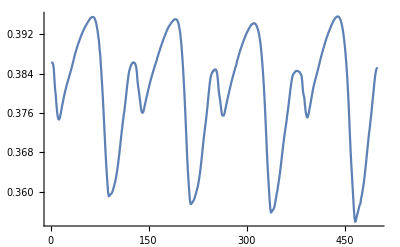

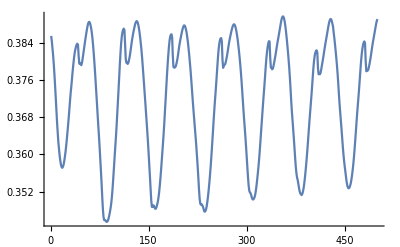

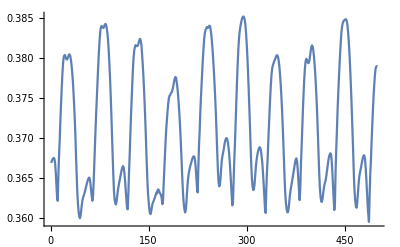

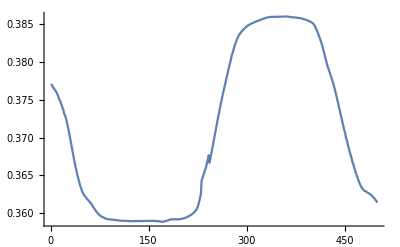

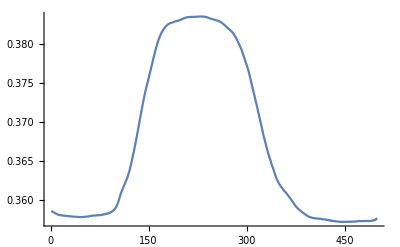

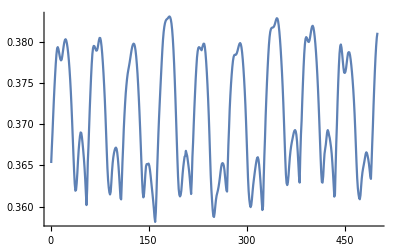

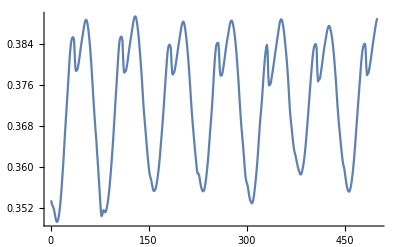

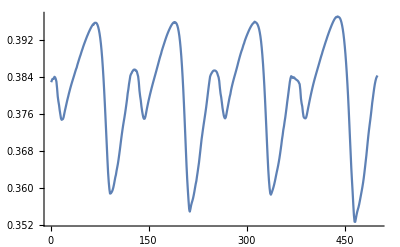

```mathematica
dataMTULintask1={};
dataMTULintask2={};
dataMTULintask3={};
dataMTULintask4={};
dataMTULintask5={};
{{dataMTULintask6={};}, {dataMTULintask7={};
dataMTULintask8={};}}
dataMTULintask={dataMTULintask1,dataMTULintask2,dataMTULintask3,dataMTULintask4,dataMTULintask5,dataMTULintask6,dataMTULintask7,dataMTULintask8};

f=1; (*(1)walk1, (2)run1, (3)hop1, (4)sts1, (5)sts2, (6)hop2, (7)run2, (8)walk2*)  
Do[
datafilesMTUL=Import[filesMTUL[[f]],"TSV"];
datatime=datafilesMTUL[[8;;,2]];
columninMTULfile={10,4,5,9,11,7,12,3,8,6};(*in order of "TA(1)","LG(2)","MG(3)","Sol(4)","VL(5)","RF(6)","VM(7)","BF(8)","ST(9)","GM(10)"*)

c=1; (*"TA(1)","LG(2)","MG(3)","Sol(4)","VL(5)","RF(6)","VM(7)","BF(8)","ST(9)","GM(10)"*)
Do[
column=columninMTULfile[[c]];
dataMTUL=datafilesMTUL[[8;;,column]];
AppendTo[dataMTULintask[[f]],dataMTUL],
{c,10}];
(*Print@TableView[dataMTULintask[[f]]];*)
Print@ListLinePlot[dataMTULintask[[f]][[2]][[;;500]],PlotRange->All],(*dataMTULintask[[f]][[2]] means only plot LG MTU length here*)
{f,8}]

dataMTULintask1=dataMTULintask[[1]];
dataMTULintask2=dataMTULintask[[2]];
dataMTULintask3=dataMTULintask[[3]];
dataMTULintask4=dataMTULintask[[4]];
dataMTULintask5=dataMTULintask[[5]];
dataMTULintask6=dataMTULintask[[6]];
dataMTULintask7=dataMTULintask[[7]];
dataMTULintask8=dataMTULintask[[8]];
```

```mathematica
Print@ListLinePlot[dataMTULintask[[8]][[2]][[;;500]],PlotRange->All]
```

-Graphics-

```mathematica
f=1;
Do[
filename=StringReplace[filesMTUL[[f]],"_MTU length_10 muscles for 25s.mot"->"_Sqrt_NormalizedIemg_Lmtu_10muscles.xls"];
headers1={filename};
headers2={" "," ","TA(1)"," ","LG(2)"," ","MG(3)"," ","Sol(4)"," ","VL(5)"," ","RF(6)"," ","VM(7)"," ","BF(8)"," ","ST(9)"," ","GM(10)"," "};
headers3={"frame","time(0-24.99s)","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU","I EMG", "L MTU"};
headers=Join[{headers1,headers2,headers3}];

dataformodel=headers;
dataframe=1;
Do[
datarow=Flatten[{dataframe,datatime[[dataframe]] , startnormalizedtotinttask[[f]][[1]][[dataframe]],dataMTULintask[[f]][[1]][[dataframe]],startnormalizedtotinttask[[f]][[2]][[dataframe]],dataMTULintask[[f]][[2]][[dataframe]],startnormalizedtotinttask[[f]][[3]][[dataframe]],dataMTULintask[[f]][[3]][[dataframe]],startnormalizedtotinttask[[f]][[4]][[dataframe]],dataMTULintask[[f]][[4]][[dataframe]],startnormalizedtotinttask[[f]][[5]][[dataframe]],dataMTULintask[[f]][[5]][[dataframe]],startnormalizedtotinttask[[f]][[6]][[dataframe]],dataMTULintask[[f]][[6]][[dataframe]],startnormalizedtotinttask[[f]][[7]][[dataframe]],dataMTULintask[[f]][[7]][[dataframe]],startnormalizedtotinttask[[f]][[8]][[dataframe]],dataMTULintask[[f]][[8]][[dataframe]],startnormalizedtotinttask[[f]][[9]][[dataframe]],dataMTULintask[[f]][[9]][[dataframe]],startnormalizedtotinttask[[f]][[10]][[dataframe]],dataMTULintask[[f]][[10]][[dataframe]]}];
AppendTo[dataformodel,datarow],
{dataframe,1,totalframesneeded}];
Print@TableView[dataformodel];
SetDirectory["D:\\User data\\Evan\\Mass effect Subject data file\\Sub03\\Sub03_DataForMuscleModels"];(*change this*)
Export[filename,dataformodel,"XLS"],
{f,8}]
```

Sub03_(1)walk1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.30470722302006680.266469410.0095335394070132730.386281160.0074087871183440570.396679360.0140119172510856480.278453330.066754048961048990.290733110.0246291214478015220.479732940.035790995037000050.266101730.0231849023384837030.430593420.01191162894964110.462874280.112513235406728470.2549022620.010.37214005567427510.266339280.009971900482641590.386274670.0079500659093124820.396764340.0180029314111596480.278584380.076658463941922580.291277420.0256918159853722070.480343740.041264524217290180.266643360.0189554725467514580.430258830.0091642216075931060.462397090.113503313403267650.254938930.020.430095311692275440.266206610.0105702920322822410.386199210.0087351338196201040.396820470.0234772950476209820.278717720.082306439218536340.2920950.0265592341978111050.481267190.0477564122810107340.267450830.017146962911077540.429701160.0090554749744278430.461633750.120427090646157640.2549352640.030.45200619885843270.266246170.0134984117069717140.385883760.0112218740817647630.396666420.032549411520772570.278677990.081189591052442490.293128120.0273222975460612850.482375360.0515543883798906740.268461620.016080151631460260.429041590.0103039791842431240.460718050.136357532282134820.2549639950.040.43369247453729780.266828750.018384165455519350.384959090.014872878158547750.395919670.044758919620395640.27809010.07451623253065810.294281380.0268099499731895150.483508630.0511270836961893460.269578750.0152006654432947450.428397260.0113958004808550040.459797250.155323177210841740.2550522260.050.429955426619622050.268679230.0218642700483135460.382751690.0177368821730441930.39386210.0581720841086881340.27618810.069158343153205470.29508210.026505325413897130.484141020.051194311420606560.270348250.0144860069667487860.428100270.0109297024825636690.459313360.167311819176913260.2552946270.060.46304901168724530.270333320.025568159705659310.380772610.0213470063644936240.392000220.072305731686102150.274443010.073274981919721860.295697830.028720810492055150.48471460.05664017936608750.27093690.013432456222131140.427763410.0114208577493036620.458800590.165548581358015980.2555401280.070.50868471246708880.271160630.03273200680847860.379585520.0250141151387094950.390957570.082545480384981510.273554170.087033815098854920.296683710.033658370784247960.485920650.06378639306986980.271874470.0130898289343608360.42694850.0152421153558364960.457632160.149377528761299530.2558889390.080.56390541220540680.272266480.041029205584346150.377788960.025378727308810890.389559990.085928414744686560.27234930.099252842579704920.29785970.0367411954231104260.487384940.06390426274593810.272985860.0134515731669750.425973580.0183913846091363420.456209090.123314270620213520.25637154100.090.56803696554672360.273032570.043879186903475370.376280960.0229532197631192240.388489350.083798234973404950.271503340.099512955819325760.299170240.032173255512783750.488941140.057286069460002270.274216950.0132006609832041720.424926310.0185494692792697560.454687920.09403075534526410.25683253110.10.4298260027556640.273341440.037551201128667380.375293350.0210253058402361320.387910190.074372162666362820.271159650.089908812690521980.300454140.024235018991747290.490476170.050463398187217030.275416880.012900952198822130.423825620.019119264151315680.453144250.06718516272834090.25709494120.110.26558389850873290.273348720.026839303656280110.374757890.0206498973672382060.387695940.059575095396200050.271151520.07961053303054660.301504440.0197412221664983140.491938140.042616642150126010.276395120.0140085248820319040.422602090.0216092010113365930.451557960.04574360014889680.25696642130.120.191523118662415480.273011080.01852952786691080.37467910.0197987318237289770.387883080.0460321739149130.271527190.075021546741964750.302417360.018960562232059440.493379940.032311981716346430.277243680.016233117678928290.421309390.0236590939321651250.449929930.0304970683971296330.25668286140.130.18684470541724980.272400450.0131705792678634070.374954940.0160964271533947240.388383630.035933622325113290.272202030.076610051919924120.303229180.0209153338526243470.494867160.0257110758115616580.277997410.0165949647066561750.419921650.022235792507344660.448199280.0212641733091060750.25636377150.140.20631657969182540.271602770.009280372565868280.375517230.0120468470515835040.389115290.0272601697573758360.273074750.078136076203974350.303877370.0263728954033415970.496370780.02911258589458480.278598920.0146681793900288360.418404630.0166978137905986170.446365360.0168815110595826670.25590498160.150.208427418855598680.270766980.0081637632065111040.37621340.0092068792917783320.389923230.020689650275020340.273978430.07662925816235220.304331120.036589588428278810.497828460.040197791489961120.279019950.012537482458395370.416790750.0110685510786575950.444494180.0157489315954119430.25523303170.160.179777365172852060.269964520.0073540956806617120.376934630.0064148257280213320.390696220.0157328917467512120.274835790.07916847189187180.304649030.0491117533548976750.499184660.048313050664808750.279314960.0109289727283490970.415184360.00778099659031584750.442686320.0147729796850933140.25443201180.170.134911997164119780.269209660.0054143992680062230.377651180.0043564077377122310.391405840.0108992877121939540.275633130.086170301052548720.304861340.05477071352784430.50039330.048142554044250110.279511990.009306006349480520.413665640.0058718659142507180.441020630.015216177363304490.25356288190.180.08756357358791250.268515870.0048033344996370310.378339910.00351603772924470380.392085610.0071529925275448450.276358130.088317910477925270.304987520.0484855923786267140.501404370.0447451453823113840.27962910.0089696013776161540.412310390.0046806903695091230.43957470.0177676916950239470.25267668200.190.055485260820506630.267891250.00512206391020982550.379004450.0038425172585954660.392738460.0063313321999499290.277004490.085256914257636910.305007580.039143728478114080.502196490.0413685362481462160.279647720.0094408074152734050.411132840.00387763567374369920.438372290.0188122321081348880.25175976210.20.034697562517397940.267333940.0066452327519531670.379639610.0049382287493161020.393359740.0096982636610770160.277576080.082625269016045890.304938080.034765456255689420.50281180.038646385191894420.279583220.0098177679646989280.410114720.00336942079327165730.437378180.0179586304005916850.25084492220.210.0185553727961241460.2668810.0092958241204500890.380197650.0070667917699771880.393902930.0168534959056441530.278037120.076894277316632690.304797080.0301230175131072630.503332960.038018171099349380.279452350.0084678457792487310.409184690.00289434474310233240.436492130.0164181350330800670.24997466230.220.00875949818617680.266368810.0106035350430398140.380784750.0099717820493200950.394477090.0268503115079335440.278554660.064350267440516640.304715020.02413703862042070.503741220.0382431318239225960.27937620.0068542070033086710.408441160.0025387496371564980.435798670.0153556974100941720.2491979240.230.0079117021483509130.265931080.01159632242758390.381310010.0133206030914356350.394989210.045454141169351910.278993780.0508216765916856060.304595360.0238334618046731030.504130230.037403753698926090.279265150.0064158167157987870.407725130.0024725699370378170.435128040.0144429345848259630.24848568250.240.0150220114171398770.265521640.0107233994529127350.381809440.0136016795847766110.39545240.0510318346127791240.279401860.044197390985813290.304463770.0325127073542726550.504510840.039442243368791930.279143040.0060019959144091290.407028380.00188046350499359120.434474530.0131830237868597180.24779669260.250.030372408063338370.26513420.0076297960365753540.382285180.0098164680578592710.395882790.0326539821566774750.279785660.0442940951537389160.304329460.0373720482547695160.504901090.044799409887249630.279018410.0059342418378419940.406338960.00093832549794112640.433819230.0121520226266551480.24713883270.260.0488693803986459950.264764710.00527962040541549850.38273490.0068963287199258970.396290590.0152538051000502060.280149550.042235638397084830.304205480.0303596384724942740.505317210.0437440115835309240.278903370.0059436127594444850.405644570.0007351194087360290.433146870.0113882223181898740.24650026280.270.053408067623927860.264387310.0040072178743445750.383185650.007964628016317230.396702430.0153144304160862670.28051910.03510337922346350.304091820.020813689713354920.505739930.037084011866066370.278797910.00535631095336693360.404959290.00144568566807775860.432479820.0103889627217614820.24586373290.280.038920170974676280.264007450.0041181935985890040.383646230.0122547493056168740.397119060.0253465364055963440.280888870.025565419282587660.303960660.018784262121695550.506170250.0321367660695882560.27867620.0049121926795683650.404258340.0020505010420265470.431799830.0106000433323502290.245203300.290.0221724177441856430.263626510.0059100078819657920.384108580.015436710035605880.397535620.03449830340135060.281257490.0179698667328716670.30382460.0218184245161854170.506608610.029826562700795070.278549960.004971517784754340.403544890.00255583498297248970.431113570.0108893588993160610.24449294310.30.012087575564893530.263240770.0087290497828099220.3845940.018608944830844520.397964470.039883177163081410.281628530.0165574271008142560.303649930.023602708976088390.507040760.026375173228601680.278387880.0052632362874398920.402806060.00487059264323036040.430415880.010708426437126260.24372422320.310.0067288451683843560.262874780.009589532645735820.385068640.0280568562066002180.398376430.041999806404118780.281978510.0203664571517761660.303453420.022120173981986960.50745330.0214678055653948660.278205520.0051016734537477220.40206860.0080284922146037270.429734940.0107784238364097060.24289933330.320.0042185621342167090.262475830.0079731483635690750.385575580.0474780963454796350.39882040.047968162200009490.282357710.0242374636488565320.303255250.020322288739045690.507858980.017226985530039230.278021610.005728784457724720.401335140.0092154487154540510.429062410.0097506661825297850.24205518340.330.0046629187971784380.262044980.0084696061007036220.386109110.072271446114376410.399291920.0571826666312207560.282764550.0232870586510394750.303063460.0180603146393038570.508247120.014310262898997420.277843590.0065404289572884470.400629440.01030142559963140.428418780.008362149538765310.24122173350.340.0074440000061038080.261611230.010837180616572380.38664050.100059354014869910.399762260.054137897296921370.283171320.017745104470070790.302876610.0141214311221464040.508608670.012142054078447510.277670140.0065671853939867280.399966360.013795502114756480.42781670.0080261323181233970.24042304360.350.0095097270161880220.2611530.0144927522342158470.387181920.14962055262593030.40024990.0507388831296111740.283598020.0118193237624573280.30271280.0118814317383287640.508973890.0103328175295156820.277518050.0065984123288260530.39931360.0150568598003645960.427219920.0090019158609782840.23963512370.360.0098756937873738320.260686170.02138075352544470.387719870.217832912808755050.400740030.063604315693394430.284029510.008099391077145790.302567050.0115566533403782520.509340680.0089964411850193770.27738270.0071510483780554420.398668540.0111283724087716150.426627290.0113746385270651580.23885515380.370.0085928884318937450.26022130.0220105550102049320.388240620.27839081841207820.401219980.073887297908023380.284455990.0082439591606673370.302445730.0101895710579422460.50971330.0092429790324042460.277270030.0083152259256143270.398033080.00644734434563328740.426036480.0117252153134868360.23810103390.380.0080534705791409070.259836440.0211434691100728480.388670860.31278867482269130.40161620.073649161654120780.284806660.013784044585188840.302343050.008312678596415530.510041690.0125029104079266120.277174660.0097843563922154970.397475140.0039708501989357320.425517760.0094225350096186750.23743212400.390.011690674412561690.259390740.031751518567849490.389139110.32869123548619680.402060910.07752951891502650.285210030.0249553795212023380.302278340.0091965279625033270.510435270.0191959739881281950.277114540.0093605255968523350.396838170.00292464896227940430.424914840.0086553109469446560.23668798410.40.0184736875486628230.258999020.045927976521461190.389551520.362757928883637170.40245140.094341260303290320.285562140.040738912442985880.302215840.0121750046105009170.510781970.0261950162249222180.277056470.0081774802524573130.396268370.0024646047089681320.424377320.0091404660010097130.23601794420.410.0230901124341650540.258611210.056378586778236030.389947140.35599656438273430.402832140.117042283876460350.285908530.0562757779305466040.302175250.0152061349426310150.511127770.027642691340789150.277018750.0071650708424728290.395715780.0022280169658586840.42384870.0085492118677818840.23539135430.420.0217444471875089250.258213540.069640105560483850.390330280.321154874958382850.403211910.14242801505925780.286261460.062872619994813680.302174170.0161171140796354420.511484460.0235923043376792470.277017760.0071749667906841370.395178690.00226982056758628230.423321510.0082181595878101970.23482186440.430.0191160265946077640.257795780.081291579658679340.390707020.327073067845034650.403599570.158725363915561250.286629730.055420385600429750.302219580.0153098566821936090.511865090.0175639219152177550.277059950.00697437622026789860.394649850.0025208783526025770.422783420.0083501233666289640.23432061450.440.0233563006042923560.257367970.092557693846831490.391074010.40559954935061940.403987740.153457229188680960.287004240.0391309673439440.302298730.0141209547138103720.512265130.0124896930187645430.277133480.0067982572150076870.394124220.002814060461889530.422235180.0076073580808510710.23386242460.450.0303412433894896530.256935690.125744470097807480.391434340.52345166713414360.404374570.171074159238909480.287379980.023487180485631770.302394850.0126575226081200880.512682190.0087630560544509090.277222770.0071573432523748890.393591030.0032447743430584960.421673130.0061916796054887640.23341165470.460.0317473860580721540.25651430.166786857531997350.391781390.63641344091828540.404748760.203813027111022750.287743680.0131280283174344970.302492490.01106745444482140.513110260.0058415634788924790.277313460.0089411505153738430.393045430.00345481314619807940.421098360.0050285669223760080.23294501480.470.0278429119741537420.256099970.17798112858001420.392123660.68836984703320680.405116250.215941755291523870.288098790.0079176005314764570.302582340.0103096328556016860.513537530.0054747565792580670.277396910.0112008418789961840.392497310.003517121837324830.420524760.0065790029596585260.23245728490.480.0224770493935995750.255714050.14643946199662040.392440960.60589356092478430.40545680.216239486794921140.288427350.0055467528485163080.302665360.0102085954995246520.513962650.0059257801555015560.2774740.0101381086906932130.391949760.0034506526168861330.419955180.0085198398761768480.23195155500.490.019707474056398080.255382390.127460077295712570.392704210.55554328795508550.405744820.233662679896108620.288708030.0040466246899376430.302752310.008840773939139640.514337230.0059103841484926820.277554730.0076134607955286910.391487850.00309646701469338960.419466160.0069459810352296920.231549510.50.025406939925745080.255007850.15272547144099720.393025920.58549631694259540.406078930.2603177953415710.289023110.00374037657801665850.30279980.0067258967966017080.514720790.0062305988737623990.277598830.0072394458555037240.390970360.00274429659760557380.418943390.0057214678428142040.23100766520.510.035385700404235270.254695190.171819324369693080.393287630.56439439956240170.406355470.25941215376576880.289284610.0050577982101608810.302850330.0047672338747350760.515031370.0062253410275826640.277645740.0075342894363074270.390575340.00247839846149858260.418534480.00676510845338456740.23062646530.520.0404753931467781640.254398660.152915310342661230.393540020.52609006210728350.406618330.26426948437581050.289531360.006355615606771710.302888030.00332539573752438320.51529860.00590031652246833260.277680740.0064015328128177810.390237170.00200033836581812140.418183480.0080863788635149730.23030783540.530.037920152294161110.25413790.125521288752175640.393769380.53350815642996650.406852260.27760467875312360.289747320.0066381334813063810.302905110.0024285160420543360.515531890.005751683134858650.27769660.00537059398637916050.389928740.00162574732287154840.417868360.0087216625073416680.23000856550.540.030213309490663570.253881190.097271117301912060.394009390.50157630637039590.407087940.263055877754312830.289958990.0058493782469769810.302892790.00207347671970689940.515753180.00468776961808711150.277685160.0056447416952686060.389613620.001724161225804890.417552990.0068900158150384470.22970031560.550.0245381797427197920.253659450.076683991952355760.394242010.394395680115685540.407302090.221413623978002680.290141080.0044107582564356540.302831650.00180509844873696580.515962930.0037795116048538660.27762840.0064789820748865670.38927360.00182703208276858830.417227820.0036696544165451260.22933365570.560.021976822527761960.253478440.085677541664932020.394464070.321122402298080870.407490160.185568654061091160.290289230.003419874610605710.302718190.00133397001770979770.516182790.0037881363434247130.277523060.006610605491145290.388871240.0016568184090928420.416858960.00252785323840781180.22885436580.570.017857251373027880.253327160.090227215243801870.394686590.286897242248183470.407662480.157354861595403740.290412680.0030552234407539270.302550460.00135363004974239570.516403430.00362849238419795180.27736730.0064005682636296610.388416320.00156001861903203420.416458090.0040958751475191880.22826149590.580.012329860787998920.253215540.076366314643724380.394875760.229046366376995740.407799750.125572740708445070.290503570.00246438875015293940.302377180.00150749530256488070.516545050.0028236585227134450.277206360.0064645919418070410.388059210.00163486618127890570.416160430.0055603736152701220.22774303600.590.0082072755152082220.25312410.050388042745002280.395114450.149729361218678470.407946240.0994405884072890.29057790.00232517241750615460.30207020.00137074915294681370.516846050.0032026132657990830.276921140.00682755196569499650.387367820.00161111671730943720.41557130.00648719487615986250.22677104610.60.0075018208361378080.253091050.0267034279086275330.395288920.088473257159172560.408034680.082330907085594550.290604740.0023896777047846930.301784970.0015717699700927240.517055670.0046664391469492520.276656010.0069823197225938030.386809790.00172410826748911490.415115140.00778308876115672760.22590818620.610.0066419028869355130.253181490.0141736289470510770.395378270.0510563883181927860.408021950.068911235411374210.290531260.00246830610771816860.301447110.00216953533563548270.517331060.00495792519385218450.276341780.0060159081537359890.386090660.00189083801292475280.414524550.0079217174281777780.22477574630.620.0050900381180414840.25327260.0075540017998345580.395462630.0295941780227214730.408005620.046722020260569770.290457130.00274179859551820950.301116440.00263818873679141050.517570750.0050008350457388780.276034030.0053841647846118060.385433530.00195121935419509940.413988320.0060014155566029270.22373407640.630.004493993931028010.25338660.004770037779917150.395522320.017188606576310160.407966120.02612465203462460.290364210.0035512311661414710.300792210.0036197103128970180.517786650.00538799484818496250.275732030.00606533957320732050.384819680.00205961008439945740.413492420.0042453045668342340.22273697650.640.0045811885285622450.253550070.0040938241325809370.395521150.0099326006208653730.407874880.0136078658752750070.290230660.00455690051690480460.300498730.0051952264569582860.517978560.0056573991827774490.275458460.0078218741602374320.384270390.00236879626434110530.413054790.00425277271561515150.22180061660.650.0046397312827047970.253729680.00405948932918393040.3954790.0058161361781627030.407758120.0073635858820985720.290083490.0050173115736713970.300256610.00594530320625296940.518118650.0065160950255358440.27523260.0103802494984344130.383856380.0028535506103383090.412734220.0051762627239264980.22104696670.660.0042902873139254840.253999070.004322053995422580.395316290.00397488495215108250.407544550.0047873599737407070.289861910.0045698595887092960.300091540.0052834836652872630.518210110.0078625903980397480.275078510.0122085170612561480.383613940.0042055809527654540.412559170.0055484233985698250.22052583680.670.0055893984620254040.254317360.0045847054705584020.395050790.00339498856401619160.407264110.00474458592597023450.289598790.0041951458339722910.300041760.0046705680870938060.518323360.0095817609574954040.275032030.0131322764737406160.38347850.00698925359738939750.412455950.00664268855239188650.22019505690.680.008261495045850.254675480.0050442181214026420.394671120.0034197769620069340.406917550.0054210548623170640.289301050.0044219744282597740.300146030.00498575600460496750.518553470.0109452794484963130.275129390.0138472002278808240.383309480.0094541584724744350.412284260.0084814413490134530.21988222700.690.011017544108050390.255103860.0053926296047710290.394156920.00375975891715267130.406479150.0067589773405630830.288942530.0044972670773984650.300387320.0057211579099581010.518875810.0100001233108353170.275354550.0123774856068467050.383126980.0094862112357770520.412072170.0080030654272732690.21956664710.70.0142469922703471140.255648240.0055573767213669510.393459940.0040315359477229130.405902870.0087651599291433780.288483170.0044969666913544350.300773740.0062020557154288280.519314510.008536873541268270.275714820.0092867778433057720.382902020.007496979170292220.411776550.0067137671084723890.21931762720.710.0151443936475343060.256261310.0065388199288693380.392617520.0040890146083582420.405227580.0120653458033143770.28796080.00390270249839893030.301312570.0059351488853937470.519877520.0084645515447937090.276216590.0068645191924374950.382618130.0054418092305374550.411377450.0062078950264011520.21912988730.720.013268753168867720.256969230.008606674305782280.39159860.004797749356671510.40442280.0190410706398605360.287350920.00337683449864524270.302010250.0051978436485739410.520571880.0088194472469215970.276865430.0060973108542370650.38226880.0040624891006449170.410856330.0057265922339062240.21906873740.730.0121302172046534870.257521590.0108056546519949330.390717550.0068149938607778830.403754710.0276919951466322170.286870060.00330167660192960630.302710210.0042293863913252370.521348610.0095445661794250310.277515640.0069550192836148910.381830420.00342121984954207130.41024760.0065756538533424020.21889538750.740.0112546629825257240.258684050.012090401790451940.389015130.0092781060435455450.402397380.032267162005844770.285843640.00331490025793540820.303848850.0034299411324739880.522335940.0097757346333632280.278572460.0075100510348404890.38139370.00320771141917942230.409462190.0072640674469318780.21929945760.750.0089779579036883480.259369340.0149932367394757760.387831620.0106176974036821920.401439950.034844042271692990.285229330.00327299107119403270.304839170.00277645101141223840.523362480.0095183611050088140.279491410.0082053512445421010.380847940.0033872510527308930.408625870.0079982907308290330.21936378770.760.0081511044562064330.260818040.017441147094063360.385669220.0097429487172850380.399348470.037994306328771920.283907950.0033799027699453470.306225430.00241337532833172440.524443370.0091508997497847420.280778820.0089637685199193870.380538560.00357425458255212440.407829850.0094837729789619620.22030185780.770.0078069125306279960.262060840.0145915057554626260.383692990.0071694770467125530.397431810.032143315617731630.282749620.00330549712279886970.307575110.00270058437459667080.525580420.0091617078732358060.282034770.0083258409079656910.380121860.00290049257656557630.406948980.0088251728696603780.22092012790.780.0079613918720643170.263453570.0092046571786902130.38149210.004572952756756980.395286430.018506546506885580.281424120.00307642203546063150.308988220.00311817069110574470.526732840.0091277827446877690.283352860.0074733158139225480.379704590.00230921060225572650.406036310.0082971708829507330.22150489800.790.0102471499217205180.264966780.0061861079576338450.379094190.00319095022616788450.392939020.0086488587897675640.27995080.0029881530972968770.310448280.0033258635688885490.527885260.0097829400367062250.284718110.0069159328904974940.379298730.002160311109093930.405102590.0081861059020359240.22209581810.80.0142815871317645420.26662520.004905621278787490.376480.002727747552211660.390370430.0051211051172266280.278296090.00266000817011992830.311923370.0041458451985687470.528972120.0104166679157550840.286100840.0060250550775730570.378960610.0022985926548041580.404216340.0074520523605254460.22270087820.810.0213592040560573360.268325070.00449178656027785640.373760710.00254219096765055580.387690530.0046739048168478860.276556210.00207598922568112950.313393130.0047125555786668810.529964390.0098273165873852090.287481890.0049033178447832370.378716670.0021607031461332080.403405590.00629868282881493150.22337506830.820.040189945845104430.269964970.0042893316010162640.371040270.00263876591394351760.385001340.0056375679005693110.274835310.0020600741746857940.314860120.0044524048578156860.530852160.0086583435212241650.288863660.00422858007995397050.378581370.00177745758884463050.402676850.0047170416220917510.224187840.830.080499860970309120.271563670.0055392672663397680.36832620.0039545805607582190.382310780.0086046296147096940.273117270.00212391072698074570.316288510.0042457445785977830.53161040.0082445899646071580.290212950.0044217232117032730.378575280.00174383312331450640.402067770.00536960318306131750.22514418850.840.14271580110287080.272860840.0092878002708309160.365891940.0064824549619068580.379884720.0134171033712640070.271693770.00186956029906537160.317722970.005219860647087240.532303150.0064560483543843370.291572780.00398447965057361140.378638230.00173246094017168520.401508970.0073372045470001440.2261885860.850.212200782538812940.27381440.0143891581454181730.363765790.0089614564297809030.377746630.0183993343552769740.270630440.0021138257927050820.319218050.0074848257821234670.532995980.00411184342220331360.292996380.0033577486400065680.378712370.00172598074815098370.400925840.009482866650225270.2272896870.860.27472278368072630.274654140.018086165497359650.36171420.0098843004263884440.375668150.0213539863009365550.269682120.0023025877058526940.320750210.0105389777928469510.53368930.0042801450343832910.294463140.0037106468800449820.378777780.00195884476687821540.400324060.0106226269446744160.22834839880.870.28257883825108910.275239130.0166470016529490050.359943730.0084670757175415670.373852540.020390279112916120.269014890.00226872737285761840.322261910.0138401661821675630.534355170.0055119008825916080.295918380.0043702284612171840.378845220.00224435608034468260.39972460.0094707727512430610.22945574890.880.25202972743509310.27501420.0119768214313383850.359116670.006152798532960.372944770.015856433666781390.269272080.0022399603886174360.323728970.0162788739634524040.534967660.0050393943192899490.297338140.0052548807953781310.378923890.00232541038859213630.399166290.0077130057392607080.23047489900.890.24467182420331630.274077960.0089762927210191980.359164080.00436228011563531950.372884060.0105002331614031650.2703340.0025735541533412960.325078460.0171951628026130520.535464750.00333212207039033060.298650530.0057463913132720170.379048110.0022194761879171120.3987090.00597411057731435550.23143583910.90.233439509966353260.273080.008123656031720260.359381090.00319174420011571460.372993160.0063742951141037230.271450660.00272004079186278540.326242660.0169300071128246420.535740270.0023123798973707420.299787620.0054339039982553590.379329450.00215163132324146370.39848980.0046432161494706820.23243677920.910.217346960629170420.272262740.0074097624735307390.359527080.0025351240429557720.37304420.00403707118015418560.272353420.00221112729747804070.327192030.015938672637076730.53581330.0027803828929079470.300718420.0044293040200089480.379725670.00196395706869893080.398478450.00340566515790173420.23344886930.920.226781683927037870.271614540.0063022270028005790.359618750.00287857839522202280.373055620.0028489587033331090.273061950.00187411236989604570.327945430.014625494558698510.535687490.0037048598375514330.301459530.004372875550356690.380263560.00201726527154883150.398698540.004829403696197690.23448587940.930.224150925175709920.270980140.0057624002128425390.359826620.0041724940878758550.373195140.00239074835707638040.2737490.00218596571649386270.328523690.0129156729139185150.535387160.00388658328611390330.302029960.0051574247914912330.380928560.002084075682403470.399129460.0079285605580292980.23553549950.940.207237363757292260.270333010.0075017532637596890.360180540.00536601669978542350.373493720.00379121134636584280.274443340.0023441562177108160.328936560.0109741388905513680.534928510.00341318275327081620.302438140.0056313572792987190.381712290.00172210553448595140.399760020.0099980991920765020.23658348960.950.195330934200654450.269731040.010287470441229340.360628480.0078371139576164750.37390340.0073851400351468450.275083350.00238363921307013260.3291780.0090930146723668460.534348680.00375055910235116450.30267720.0059891411707700840.382566860.00147813728102841020.400541410.009767560477936680.23759109970.960.194019842537620530.269242490.0112534864071163880.361091550.0153264864782109380.374347010.0112261717744720610.275598630.00266216524668038850.329258420.0073305010050819340.533609550.0045288557935594090.302756890.00604945680132382150.383556160.00176783566687313540.401535560.0084779160937826470.23860166980.970.18602347888700810.268830650.0102457785276679270.3616030.0308546715774588170.374856080.0144009473996308120.276030120.00334710836766877140.329188920.0059251474244968390.532740020.005160313857245650.302688020.0055971471006872670.384644830.00221814956862186360.402700380.00768535762063110150.23959164990.980.163628033499428340.268497220.008073476082749360.362156380.051374271324818810.37542320.0168908287397164270.276377530.00360999436084644870.328974770.0050832145585834060.531720840.0049343624262674050.302475950.0058144434700725610.385862650.0023608102936109420.404063040.0069396730655235530.240585211000.990.158090482000469740.268177260.0062389987192438490.36280860.069074318130928780.376101640.019162745034446870.276709270.00327239588235706370.32862860.00417245523054865860.530557010.0036459956871614710.302133610.0056312234655474630.387210940.0021842292620766010.405616520.0049942022769423920.241591391011.0.149943853605421030.267856790.0054904887294153340.363573590.079822033284590740.376903970.020378871762210060.277039970.0032270738953713920.328146890.0037331812385148710.529245660.003322317255833970.30165810.0055172254185890320.388683550.0021146591210198470.407357940.0042364486329383540.242591641021.010.144876489130317480.267538470.0046421111276006980.364442770.084123846240908250.377819840.020478557250934250.277366870.00326858126337337740.327529440.00312027599345613160.527788410.0041575768406587840.301050050.00569898450180030250.390272610.00230054708017442140.409278530.0055563327759292450.243578071031.020.14865035214402960.267255220.0038255787823821210.365381950.07401544774872750.378814430.021186298558080810.277656440.00280769104679387280.326766660.0019773394470648030.526145360.0043683511124197190.300300950.004920409409205750.39201780.0022575791666738850.4114250.0061941247263836330.244569441041.030.149556402714076160.266964220.0045106774525145160.366430940.0619807569489205440.379924350.0226837174562973460.277952650.00211054081897703130.325855780.00154486088807764280.524375350.0046483573463062630.299409240.0039478095248657180.393839390.00222558797697018250.413709940.0062521629659872950.24551071051.040.159287586200971720.266696180.00563466707006053150.367556350.056201565887497390.381114820.024766445310671780.278224330.00235804913342825850.324786280.00198644839898844950.522515270.0054324840998632140.298365860.00455007211278368650.395684710.00226092560111726750.416075180.00603156242775192060.246370131061.050.190767767384522720.266469490.0066301148746615980.368733290.057712439045619150.382358710.0266943544575250940.278453250.0032758215340568030.323556580.0021950798811013280.520441480.0058456722391036570.297170940.00646771737215196250.397701750.00209457685126359640.41868410.0062424474628685480.247242621071.060.213506597758090250.266276490.0078508542711958030.369959180.061501427928649020.383650050.0275160150135118730.278647520.0036249115870557310.322176340.00231261090615991460.51825520.00641344350314576250.295835790.0074827237412285520.399774520.0019967160524884390.421403960.0060374457189183570.248059851081.070.199217812439758670.26612650.0082715903437713730.37121570.066747477152856410.384967630.0274411873174596550.27879810.0030629236383756290.32065550.002382109448626130.515962030.0065251845221048890.294372230.0067889005350857180.401905330.0022467886533298540.424235790.0057385071407928780.248817421091.080.15918781216175950.266161380.0082383250055518970.372356570.073124649531934570.386165030.0270258321490763930.278763120.00287532852533170120.318989920.00221990582723952240.513617840.0064179061604388520.292778690.006956137572258210.404029230.00259193817739577230.427107730.0072377028455736470.24948811101.090.140961009531656880.266223240.0078639767372812590.373530430.070651084042734040.387383920.027254632491065990.278701020.00285489634101890370.317195050.00191191982672449030.511172170.0060046490566812490.29107170.00721941419146551050.40621290.00347108092941677150.430088760.0083457531396359560.25010051111.10.148086939929997860.26643510.0059796100261507050.374595230.0561227559082299740.38848050.02553651303948910.278487910.00251808631037877050.315260160.00157018428578183920.508641150.004860903709392760.289241110.0060923872825118980.408421270.00658362675479473750.433128570.0070467986261295650.250657061121.110.17453145835266140.266694580.005797316933526270.375633940.04272485993178010.389531780.0214621046885854170.278225950.00257902128089737780.313192040.00129773936327875760.506035820.00480382364757184640.287292740.0071754235931354820.410629330.0133086212527694390.436183980.00649308582561476750.25115831131.120.186396558373084530.267095120.00725853060722557450.376534920.031663688546064790.390424230.016110914394371310.277819570.00313833461150075240.310987550.00109841328186389710.503350030.0044774949690316040.285223220.0128315410041658330.412836440.0229627626971309340.439239520.0072474544489080040.251631151141.130.160091377745008120.267207130.0070080498640641480.377684280.0200656699021153630.391534740.0106740928220443330.277705490.0041516362057909160.308777640.00144923210050937810.500686590.0041343722802422930.283156240.0225804183550598480.414987490.0332296191081682540.44219890.0076683794878296050.252069981151.140.119668812842742290.26727040.004754189643869550.378830080.0119446206630481650.392615580.0059986835186714710.277640960.0055717296459173160.306578060.00214705527951696350.49803060.0045178318840162710.281106670.035538951528706650.41711940.0408352073328206440.445095090.00735692153952304150.252520391161.150.078709369021152440.267195410.00317630475103826070.3800420.00642316750618813350.393712030.00283204636865850470.277717420.0076759410659407240.304455550.0033299058016199550.495459240.0058894824565902520.279135410.05115454609612380.419179380.043206373152563170.447854820.0073663369453495370.252965151171.160.044644952547296120.266918740.0033468522575709720.381364350.00371621844598925670.394444520.0014012988697327350.277998830.0099409633106413670.302473360.0045456562527000920.49300830.006980823246136130.277295690.066302722208515030.421158270.0410664421078853760.450455510.0079584543208239350.253423851181.170.0248038698799631850.266810430.0042345691512998390.382423190.0026119655991624130.394934410.00169774477108021830.278108670.011643981370164240.300607190.0055133098353166210.490729820.0071849042686141770.275559590.076117863308784380.422997270.040060384282408240.452831440.0073922485013284350.253878371191.180.0211269471717777170.2666720.00540358157380962850.383418960.00242348615682597960.39539230.0040143762868559110.278248790.0120808251863232740.298891880.0062483410876952230.488579540.0094184385649316480.273956040.07811036898960880.424735520.0395412421356972840.45504180.0076317797693539640.254313951201.190.034245454172032050.266487980.0053885178785085110.38436620.00205907216117925170.395839920.0055016058398063640.27843460.0110418642181708240.297344560.00732736376319319950.486670990.0121958514462672950.272499880.069472789508113470.426249630.036341879496841130.456963820.0093822380204502330.254669181211.20.056485902557225480.266490710.0044972402679046150.384869880.00192590017140980490.3960480.0049215473067850640.278431850.0102385150165031430.295944590.0091419942225487850.484948340.0135161618814694080.271172120.057299289797714910.427608860.030736418222748610.458679140.0124033770137250280.254996261221.210.078759017742719280.266400020.0045132090245683510.385272890.00257244672876653920.396299970.0035777136689027760.278523250.0111524049392396540.29479920.0102580133943263370.48353930.0156131284474698570.270076910.047530673290289140.428712360.0245268046784816620.460068350.0180140593478647530.255251341231.220.09229015085936010.266243830.0054748394020434750.385669290.0030049614575723060.396570990.00292265484891269250.278680340.0140721687223060480.293946590.0113317360309062430.482468010.0203214071455584330.269255580.039231548861307510.42956260.0196695568098741170.461128370.0252049323169057020.255459031241.230.112860634173123780.266106380.00642318382238354050.385960480.00343675128258034330.396781080.0037474326365903580.278818280.018560721988268750.293395330.013491529389955630.481761370.023742808433331820.268721450.02987429132371340.430135330.0150149129292971830.461833430.0325756254821767050.255615791251.240.147775372911628370.265983270.0075830960611430310.38615430.0042543330785351690.396936240.0054681857326530530.278941570.024905789556597490.293154290.0163341689938423270.481419690.024361380656403710.26848710.022074005231018680.430441810.0099859621282540490.462197740.038951525711899360.255718971261.250.179310467119332680.265850.0101551189871583840.386277260.00539304647788134850.397067060.0079568781747916730.27907480.034727238719726740.293219790.019321146212559750.481472720.0267333191331408060.268550830.020197523580428250.430435140.0070670260099298470.462177650.0429196665963913130.255719041271.260.21274029208697220.265854620.0134716315257015390.386184510.0062710597422444430.397022460.0113001184984995090.279070180.0472412726125579360.293552950.022563008795182020.481790730.033176476665319870.268874440.0224290480410378750.430271050.0070304255008995640.46193760.045988218724078090.25573271281.270.25906951125724650.265645930.0157563629662225670.386251450.0073036976583470030.397167950.0156939298583960440.279278250.0607335676874499260.294124710.025333305916821360.482471910.04166022512175790.269427630.023666856128703880.429760640.0080210995263522730.461302830.051559885824916970.255548061291.280.30787335016174560.265572390.0157274456889630770.386128610.0088978687845999060.397149750.0204131892927531320.279351410.074136937338093730.294861130.025622271705189980.483312510.0523136004409512360.270136360.0236833205529875870.429147930.008695329176081170.460527090.062851146669486570.255362071301.290.34704176598278260.265659730.0143503750797151980.385804580.0106017681623120380.396940450.0250588193315820980.279264520.086141757775187940.295730910.0247515277697554250.484284590.062833838145653910.270968450.021669748720643770.428444330.0084991163747791180.45962490.075422003367186420.255186611311.30.37009374007136890.265822720.014858619163743120.385377270.0115629452485033980.396633770.030884010122655010.279102030.096245019782478680.296679160.026151523588063570.485348220.069340509671420570.271870160.0175836326105653880.427689910.0074916494595067090.458639830.083137691331648110.255037061321.310.38445609526964970.266424110.0166835103692345550.384347030.0119712018542937510.395878030.0388828462072669940.278498980.104002423370471340.297524320.0292560419621041360.486310840.072488627160164080.272669610.0146069409638737310.427047040.0065230299687864470.457753990.086565807307284250.255061111331.320.370920999944921670.267899190.0179457435734647620.382485310.012246494558747860.394235390.046805182176005320.276996310.108350239913623320.298114210.0328640534114472350.486725670.079369134886369580.273225510.0117811404434540330.426902680.0064130034061494560.457458580.087492636876609670.255321231341.330.34630530258792860.268497510.0185411913703836740.381406920.0125306915391446440.393450630.05042136241648030.276377220.106334762419264720.298998830.0375925466642094840.487707680.088973685212626260.274056320.0111429859331543360.426273150.00683562032651131940.456531230.08653321876151330.25559961351.340.36852765981736020.268653110.0195436049699642570.380546860.0122555693033316780.393030350.047100807772836660.276215320.097294509991288250.30039690.0411426722216154950.489333220.092633916411171340.275363490.011481499779541570.425209390.0078205615204710450.454973910.083417421190492540.255996861361.350.37615908816071150.268950470.0197744509508645630.379438150.0105493100033046560.39240370.039240705524367210.275904850.085858555727826010.301956860.038254671912879550.491024890.084350954635430660.27681580.0097664979677869780.424225960.010343502410035130.453403870.078026450006153570.256665711371.360.304929040572548050.269344690.0179852060913328130.378419050.0103176111850671330.391736870.031452504098563370.275491140.078011123264688860.30310650.0306812336868946750.492434830.069965064455311410.277883540.0093684894671654940.423282690.0152529434388306850.451991190.070007999541574150.257073851381.370.188932921664580870.269987440.0149226743834547610.377309180.0106703579921759650.390870460.0242576769830403980.274811450.077131721880526960.303885610.026702332596981660.493610870.057882903882064410.278606560.0118820408691842660.422390770.020145613589460010.450738180.058298009544459540.257262811391.380.096962816746139530.270484630.0117891289564359210.37642090.0083608057950961340.390182590.0187292305833992030.274281250.079704194762557750.30453290.0307566844493614160.494756190.049289535934752030.279207190.0138255597800550060.421396020.0211042330593121140.449442330.044089725086767970.257183251401.390.053919154151098260.27046820.0085667240816914590.376108360.0055109830736177760.389904830.0157888692421936750.274298830.077204832809448940.305159430.0388473574976016950.495885770.0488184705655788640.279788670.0144625023487952670.420340440.016293170575059030.448124650.031758168097006250.256890141411.40.064900683615996020.270238110.0071455746884954970.376079070.00493467264255322350.389892830.015671111253793330.274544620.069209753709161280.305692780.0465927307005721960.497032270.060707251431044620.280283920.0135566520894117580.419138320.0099603660450142420.446706570.0237953540488068760.256336551421.410.140436689419028730.269840580.0088490252043650370.376287290.0065927357279313440.390109010.017130200942061630.274967310.064934839493891640.306122210.053144543483910490.498234810.075075625860168890.280682880.0118056834961557910.417786490.0056427476616682770.445155160.0214127614372364860.255656011431.420.228049253171180220.269191550.0099596126864260930.376827770.0080159839704391670.39064710.0184082696523333140.275652150.066685520973405010.306439830.053121779262401480.499458540.079813286685851010.280978130.0090713560144440340.416326110.0042871781136575890.443507860.0220097247753028580.254929471441.430.248709297216567840.268432390.0107542858321345250.377507570.0082973192253678090.391320640.0186684032113584830.276444870.066622672254892680.306709910.045877304971158280.500673480.073580297077854780.281229320.0078613846920409860.414836840.0042708888227403190.441847850.0237575071531762570.254142581451.440.197606303940051940.267797410.0120009203154028570.378084970.0072299046647793550.391892220.0173657325930778630.277101070.06243029630770.306908980.037871188180771490.501777440.060617051843552290.281414540.0090965172998953990.413427790.0037479119219946170.440297390.0252005222825452020.253373271461.450.134045870422328050.26716490.0112331776380565370.37868140.0054594651120832540.392481580.0140765802567691510.277748510.055422091086842830.307058820.029184511548133020.502764030.045511699060125660.281553990.009999175332708640.412130450.00284522191356313380.438880270.0229825186460242760.252663921471.460.091056002893245020.266543540.0087267459434044840.379284370.0038894230511092550.393076730.0097267824241585540.278378560.0450218862513831750.307165890.0206228054698966640.503643470.0355188873863014550.281653660.0093129308349683810.410939380.00225641584194375640.437587750.0197247574918754530.252017281481.470.0542499909642738250.265940370.0060132597160867670.37987680.00313229147356362160.393661340.0060401021112503330.278984490.038316892428732240.307248460.0181447599989732340.504424690.031344664555335720.281730530.0076797332128567980.409860990.00189294982352078990.436422930.018343013352803490.251429831491.480.0262385357894664470.265359940.0034952449824742320.38045250.0028780453422637040.394229380.00359877306385701780.279562320.0421272159464054840.307310010.0217902303401812140.505113810.0298785050829307520.281787850.0073283033967003670.40889570.00200260154232171070.435383890.018874341758898350.25090451501.490.0122653564157307740.264797670.00339769458751216670.381022540.00263973344669772660.394791460.00281717941921095450.280117180.054552434353815490.307339950.025167024759105160.505699840.028102385296821280.281815730.0073440348823851990.408046320.0020980337910771690.434481580.019067810342609470.250415821511.50.00715574964559107740.264272570.00366720042591726740.381571430.00283410514413673720.395332150.0041872320329468430.280631020.067689334544191540.30733140.0240077667114918240.506219310.0238229714895063750.281807770.0066408839346235670.40726240.00174082904198877550.433665040.0188607297236932920.24992111521.510.00305064432254338560.263767470.0053784411534475280.382105260.00308854092968168350.395857890.0107944634661530390.281121350.070671498874321660.307306770.019586021589855040.506694670.0190401129855024730.281784830.0054852510156832290.406535840.00157975937287026330.432918220.0180741483148600430.249421471531.520.00056870657418646640.26329350.0093242054381202970.382619010.004415027488043310.396363440.0226701678371458330.281577940.063638752458473990.307255080.0169271282524997850.507133490.0179103325441390060.28173670.0037315298498611870.405836990.00163751005037957770.432217240.014879795411693420.248881311541.530.00020571248012587740.262845240.0130018441057045880.383106410.0069532741386065380.396843150.033603399398125170.282006670.057346404559478120.307198780.0176278630167050820.507546620.0222484977369324860.281684280.0036290901583408380.405174920.00154805771654142710.43156230.010657989237712290.248322411551.540.000045355871961738090.262420250.0154627576151292350.383568550.0083455979483121720.397298050.037206674917947250.282410350.057668182455332480.307141190.0189544123263906750.507967290.0272524045820476750.281630670.0051911234240328190.404512520.00138355793722498410.43090940.0063774308665118040.247736881561.550.00054168314503782670.26200630.01582140928608810.384016610.0100466043363327660.397739280.034006302756581840.282800930.05961662475436630.307084930.0195950964664334050.508382020.028165854974056940.281578290.0064710066573206340.403865970.0015573377049592390.430277860.0054286044351586010.247123411571.560.00277561677649213170.26159580.0149814764845742750.38448350.0118710131367428630.398198060.0317241391899240260.283185740.055353324852744760.306984020.019507450640764290.508798620.029971338266169380.281484370.0069293138060599960.403191940.00197353442954598240.42962870.00796137471527290.246473851581.570.0047679384832530830.261207070.0176383497643411640.384903550.0139282517547012760.398611870.0295691178749854130.283547830.047318788290329910.306925360.0181251126840804330.509300240.0314025393661184760.281429780.0075748640951438690.40245160.00225763799970136540.428901220.01121028393488690.245748721591.580.0062286864533854160.2608090.0230485208259664440.385355120.0156640810218601350.399055750.0268956932258546180.28391630.038294900061929430.306822370.016307027560286750.509771860.030932103934430990.281333940.0084278258895534240.401722010.0024938584353386990.428198390.0122428974133162380.245008411601.590.00636633011632033350.26048610.023305592490503690.385755210.0140338800604206860.399447440.030334028552833530.284213450.028427862451985810.306673810.01738133392858810.510170170.0309792726318961380.281195730.0080920015016740870.401063830.002460463594076090.427587930.0117789118298403870.244269761611.60.0049371271962098770.260076130.0187006419979213680.386215110.0122634129892350150.399899750.0386827982817951960.284588520.0231328536305712880.306570180.0223485975227683020.510673860.0302275470454278770.281099350.00702087042913106250.400297380.00247984027959077860.426849090.0119199701408863570.243480241621.610.00352652401140310940.259890860.0192286639974391870.386501270.0152657964745185480.400177230.045967389530269310.28475720.02416711024062790.306377140.0253189078418133360.51092310.0273131721756103350.280919850.00594749262510758850.399797530.0027661065211554890.426427730.0114843888826799270.242786881631.620.004081806331202380.259352450.0257947661718130360.387093390.0217132213153935360.40076010.0572509086413647140.285244550.025748590875919620.306254450.0232957078809051430.511486270.0229135379193517940.280805790.005024099235972420.398958990.00281975242292889460.425608380.0090880677383154490.241978761641.630.0071230273736960280.259008880.032072850265399660.387523470.0315944465233133350.401180610.069382162617781310.285553310.023097703763284230.306075490.0198195377451553730.511837220.0183987380943941430.280639460.00520270532501856950.398343410.0025422106869785360.425051840.0066367080636582150.241251691651.640.0079105638844942650.258665270.035680111924746140.387958780.054848131111591610.401605820.076838615568697590.285860380.016481261496542010.30588370.016546972684490170.512148480.0143741308384591120.280461260.00510526830474460160.397762210.0031190165033893660.424538710.0062687532991798750.240527981661.650.00623697728589386450.258318560.0398086802888659860.38839120.085273427951444130.402028340.075643201759245940.286168470.0106148457215891560.305699730.0132659578539900040.512436610.0120589655924659940.280290370.0043578786129509530.397211970.0045015352110896010.424058440.008789680780458360.239815091671.660.0057279990354386890.258053320.040265677786679650.388747380.103028869926703060.402374910.066350843178817690.2864030.0086345367729148760.305509190.0118817989161334790.512631630.0144477667328419880.280113410.0042373394532661850.396781960.00522345139968693250.423702130.0104228715945676560.239206221681.670.0058402609969970640.257655610.03587213404063390.389217920.102695784256301840.402835750.068636556858932330.286752720.011393973258004580.305339130.0133383287869381780.512934590.021056284714476730.27995550.00426097202319204550.396204420.0043657718037042830.423195120.0086025488871306690.238451641691.680.0066843409244139730.257393170.039054891154596220.389553310.106856273737930140.403162640.086938935161145980.286982250.017752781846160920.30517780.0164100376977396250.513103450.02709252750115270.279805730.0046675675549022820.395824990.0030843483987186880.422880270.0074043674624640950.237909861701.690.01138625874046470.256993750.058846766363891810.389998590.153307372144673770.403600180.110788372748703330.287329670.0247283889510552140.305051790.0187817653169011220.51339180.0269849180747072020.279688760.0057190521214608390.39529070.00282383640471660240.422404290.0107127942134923380.237216991711.70.0133272652541081650.256701690.093577608239529530.390336530.259081628954251630.403931380.133843676933164480.287582260.0268136204703897550.304933890.0184434029117519320.513584790.0213139186360898240.279579330.0059658005411366450.394911280.00269808160841267370.422071950.0121572506790294920.236721041721.710.0119173252533781110.256340270.127498845590792050.390734150.39152999247868040.404322330.152558022066576340.287893130.0234780278266694850.304824040.0162812854537335050.513836310.0147667309669300760.279477380.006399402760927530.394443640.00213205854050728960.421650890.0104432368610173840.236139221731.720.016781857194620540.256014870.14377365958820570.391095350.46159559772264880.404677210.162604462366156220.288171430.0213640855154181020.30471640.0142906373553054520.514061070.0106268375924775360.279377480.00667278066145910250.394018450.00160969999239431930.421268740.008377084836610860.235614291741.730.0225980296638232970.255692970.141715079371464850.391447910.482119298973668560.405023890.161674734240138870.288445240.0227871209964989160.304616470.013692210540270720.514304780.0081447054305984840.279284740.00580169889016576150.393572470.00147903438073605180.420862220.0066793011917877520.235079761751.740.022085651854175930.255377020.111935459435424340.391795040.52829764892257150.405352830.164630486959457560.288712560.0225600432273967350.304513920.0131702762816975840.514563420.006981985307881950.279189580.0050094881914639710.393100780.00162186717428761380.420431110.0050189493764106760.234516871761.750.0202022216942891850.25506720.089055853651461970.392134780.60796105265967080.405662660.203251984611943660.288973310.0185807505953551960.304412310.0107771953775933680.514832750.00690997181671874640.279095290.0052332880877026620.392613580.00169549208584886130.419984020.00371855959926085030.233939721771.760.0208405535916042880.254759040.107645501915089180.392466640.65672978751950120.405966940.249979404611631540.289231320.0136662704001192860.304320520.0086008980693552150.515107650.0086034731885820050.279010110.0057118474997858060.392129580.00186624783168844610.419536440.0047532316724439290.233371891781.770.0221701039092559340.2544540.12997049784967340.39279180.60803767022818620.40626610.25817499922364690.28948540.009729839899838090.304233860.0073207126720368680.51537180.0111272833740573420.27892970.00561648944035285460.391666060.0019902186585562010.419108130.0060072282895646820.232822641791.780.0228777416682676250.254167090.149372297239247910.393075910.49762272234388390.406537390.26119243637884880.289723190.0072022204942377310.304191940.0064362692886405490.515644590.012832824622370610.278890810.0054269182151886580.391233670.0021381366179703010.418695450.0066646275586460360.232336451801.790.0241879373825979740.253882180.19038707910260520.393346340.43756752482159920.406801180.284742307978185670.289958170.0061136490604724230.304170860.0059048804265159890.515902680.0119407110041869140.278871250.0059984229569966950.390844380.0022386256998831370.418318010.0076154570050348390.231910951811.80.0257155543822466560.253618480.243904757270778150.393587180.486882154856435430.407040780.307816464954663860.290174650.0052824928421537810.304167870.00469864960189722050.516133160.008679326201723260.278868470.005132834432919570.390514760.00245689891508917450.417993540.0082594675314387990.231558441821.810.031469712628080730.25336790.299222724948758570.393809570.49519397882420860.407265270.30154257644345280.290379470.0054576140310053160.304176010.0032674350416789030.51634450.0074021016422605160.278876020.00435193412428669550.390225420.00307739717140320970.417705040.0086167860096378730.23125561831.820.040299922302100410.253131160.334318173158173470.394005640.420618736353066740.407470850.258311797653467570.290572160.0052021475182055470.304209270.0025621071792136620.516562240.007568452531305060.278906880.0047459553094522740.389961890.00370252567434188870.417426210.0091192452527183370.231041491841.830.0475670640811488440.252913010.3028069160622370.394208180.374546479976657240.407669710.215673685199837870.290749040.0042268617092198810.304197020.00242574763452615280.516748060.0066838650316641360.278895520.00540732669971559150.389682870.0039858788081535970.417158740.0078751686357597960.230713671851.840.0479408620253906560.252712790.23941332492147380.394382230.372524280851593450.407846770.217095985512528980.29091080.0036646747346709950.30420750.0025784107088379810.516954420.0055428710083607890.278905250.0060389603293191080.389410660.0041118682178096780.416881660.0070756681571686910.230460081861.850.047549415772187070.252538120.21563964664792650.394557550.42865173394907940.408011450.25507468460467750.291051470.0050642608733014810.304171030.0026467013350952480.517135310.0051264886922112380.278871410.0081623957622212230.389122830.0047810047620688520.416608970.0082438688329392360.230133611871.860.046284388895278220.252388510.208118494905716070.394713440.55444186074778460.408154890.295977546773146360.291171620.0066201100890747230.304128270.00302235899035537430.517340270.0054257275110785440.278831730.011092571944157840.388797440.0066066326681692590.416299730.0089101545750526270.22977311881.870.040917445661536280.252268450.181988473039332550.394855780.630898051263720.408277510.30181494702152550.291267810.00751467115231983350.304060540.0029473785761031550.517559860.0065692453866486750.278768880.0154393963929102020.388429380.0094659347517372150.415956640.008673709534143330.229349781891.880.0316454694733768050.25219050.13987011485327860.394970930.55329093300165970.408367040.257996092809538560.291330170.0076645408789439050.303972760.00307166855900527220.517798620.0086753404272660720.278687430.0198982125396617650.388017950.0120588312875436220.415578360.010726452850142280.228859111901.890.0209459164154356740.252152770.089320452500847320.395068110.37205467844886980.408428470.179075997004463250.291360320.0055105781768199470.303850540.00193464412341164540.518009530.0067523433933317850.278574030.018378233759655830.387616140.0129054191929753040.415224530.0075872883356385720.228327441911.90.0145047133299721630.252167850.0484942173344319540.395046920.22501022011411510.408411650.105711463208565670.291348270.0046770007190516280.303865490.00190098180730297940.518293820.0069324561743533170.27858790.016144516758125950.387216580.012894136207294550.41483790.006898292900880360.227838791921.910.011968075532650180.252320290.0248508703897056850.395039860.143680001440547070.408331860.06405566970351730.291226310.0044015623365303810.30361780.00208692805260631340.51865840.0075524243172014920.278358060.0138444692859670430.386460370.0114904137433417580.414177540.008069621814043140.226841941931.920.0119343700560729050.252455340.0140252710205968650.39496390.094216922076603520.408230610.043442071415785020.291117990.0042858802494971620.303531950.0015332229561455640.518983890.00864093679012870.27827840.0128895951584912970.38591630.0091748387885509770.413677620.0093502674755704930.226154111941.930.0112041082302073960.252668640.0099981996608552850.394791310.0592582466662028360.408047730.0296232501631840260.290946390.00464642610530065050.303497070.00149222841193287670.51934220.0095045911626437060.278246020.0130976561459357260.385368280.0069400743214053490.4131620.010176466153602480.225469941951.940.0093495087196481180.253038090.0076149726759074790.394461270.034999045527409550.407716970.0187014070323559130.29064770.0048461340455792130.303494390.00245919390446791350.519677290.0097728415321096820.278243540.0130323908128525570.384892420.0052312731649924840.412715440.0100904937478592530.224822511961.950.0086723903683352270.253455780.00645082223772369850.394016130.0200466107895807160.407311070.0116974998330308650.290307730.0042673160807392090.303626690.00327924664574276440.52005850.0094432842361726230.278366310.0127616648284483070.384493120.0045949684641914930.412304610.0094016166578704630.224325961971.960.0090740101630371020.253990460.004942292498429250.393375470.0116383060075745240.406759010.007647285262370480.2898690.0032224753224035290.303926260.0038709743074284120.520542430.0086217023956927760.278644280.0116976381219220890.384100610.0048774473689525990.411851840.0087712648272936340.223925611981.970.0115208436101835710.254669870.00372543881587168330.392505550.0082284691874873250.40602950.00467531285701415850.289305730.00279781315289300870.304402590.0043128218150227620.521119750.0089086202329807190.279086270.00946053245803060.383726870.0053551136747240240.411366190.0083146767049257380.22362911991.980.0164403776839573970.25548460.0036360910387169670.391410860.0078692299445775640.405005790.0033461997195843170.288621690.0035315819820963070.305053570.0047634397704570260.521838990.0101392713374978790.279690410.0080051214727420270.383293730.0055375359816193190.410760580.0087004770079814240.22341952001.990.0173594780824824940.256400420.0048600682265577290.39011180.0067445517702179940.403745150.0025773168864077440.287841520.0049380509978270140.305888750.0065018571010420520.522726850.0109416258334907620.280465950.0071754676547165170.382759330.0056535483407746360.409989260.0078363342760653030.223247222012.0.0141940505473820980.257612330.0068188381312964930.388423570.0048129812602294270.402100180.00357920032582678160.286790650.0073810198931071180.306893090.010444786880729810.523653380.0127352789184946020.281399750.0087239247370156820.38230360.0052423369644136580.409213480.0079385643227135280.223399732022.010.01212709119565620.258935990.0077823706292797080.386508890.0051203772957396660.400230750.0048813465512185630.285618590.0096923057783770760.308063210.0134693234751938480.524757150.0155274774718091940.282489690.0113916694688938150.381719760.0043340599448017170.408229110.0094246561485907530.223649312032.020.0108876751564852760.260395440.0078714801039535820.384348140.007881194429745220.398114620.0047045639879667220.28429660.0087610672915889070.309370730.0120065047768737730.525980320.014796484562160660.28371020.0095152110045268550.381051940.00342635420692408850.407097270.0097423066323616520.223923452042.030.0102090476653069060.262025470.0080731823251948350.381909040.0092591396190749940.395717730.00388482424617664270.282782910.00670333458853761450.310785650.0083500583863646610.527268920.0121953781585181190.285034060.0074661853446002050.380371830.00280130347457517360.405887970.0095090082274400440.224326722052.040.012654079025679690.263766830.007092461373231470.379244220.0074832290588912980.393090710.0042843843863787280.281121960.0052218423974271670.31229070.0055199638358920560.528554390.010041489366820170.286445690.007512522690237330.379738920.00267056048027804370.404685090.0089565874612163240.224732912062.050.0204032882922454760.265652350.0067015232534529550.376349190.0059769485580924380.390228590.0052162032289060140.279271870.0038219808192443780.31381040.0038123585354211370.52977750.008467960897683260.287874550.007913356743574460.379191390.00282363514558188350.403545140.0085632722704925960.225187622072.060.033679316229062430.267645470.00705141333168448750.37326940.0057530995533885760.38717710.0055652695105639280.277257160.00283232906339559930.315313390.00304444665005395180.530905740.0078844553053145830.289291360.0089969327493533480.378760160.0027300345361945840.402507910.0071967469063657760.22572742082.070.054906822070165590.269671320.0049022691075044690.370080670.005227058820528190.384011470.0044169385127613550.275146550.00214610481714751350.316802620.00306656596040089060.531904080.0065672281593459310.29069970.0085399925056456450.378495660.00225783818317502750.401622940.0055476326026582820.226418782092.080.08611880280843950.271587650.00323433757268700360.366962670.005775831831380510.380909080.0041273788765148820.27309120.00239979049836332560.318253380.0041675476355032320.532733040.0054151343494360470.292077040.00716811715687860.378439870.0021218876683004320.400943240.00646135100277150150.227312412102.090.124511079728251480.272998350.0039822183636790080.364350170.0068881152312794780.37829230.0046024297487160440.271541320.00256621462447021150.319711420.00554468500482496050.533457560.00448407980397009550.293467780.0053316651091601440.378528310.0024395990186290280.400390970.007786760183877020.228374042112.10.162152884355407480.273893950.0070165482964631910.362236760.0078924564517875460.376148640.0048070157347363170.270541090.00255642306452813060.321242110.0066151782905337650.534146060.0051103549024581870.294935790.0042734863909984090.378711110.0027478700383846930.399882470.0093005982077543590.229664862122.110.181735075134081020.27457230.0103167804379155590.360303240.0079037159038291840.374164590.0055297620523354550.269775030.00363054823924539950.322823690.00728130791239263360.53479880.0056148244016878830.296461180.0048833504111298570.378943210.0027967518019407060.399399640.0096650374854167170.231011332132.120.17993120095327720.275124110.0113742649199660010.358513360.00714454256818020450.372309470.0068159348659932780.26914650.0044437187472222970.324356120.0077534040498688740.535353370.0049090954628525970.29794730.0065449424395402730.379218750.002687169005156620.398989510.0105612302941851520.232285762142.130.16029318189972120.274975630.0115385338230821650.357583990.0061552595570191680.371285960.0084029538106033460.26931610.0048218531504097570.325769250.008216059263006440.535785890.0055797944434738160.299324680.0079311225285949170.379513630.00288102814628969080.398664350.0115573450887187270.233394322152.140.13796361181908360.274146870.0105504983016830050.357512670.0051973690597183760.371096320.0085986146822798190.270256320.0049664577494667360.327033970.0089758049318250880.536068010.00730084386067094550.300563210.0071230098495647780.379857950.0030635655193812080.398459970.0109121613497327880.234408642162.150.13365844688516630.273202530.0086690219387379610.357665750.00518596634392397460.371130030.0075788151874183410.271314410.0048773696729705340.328130240.0101883629361848930.536150380.0082252492855990860.301641690.0072201199742759290.380323170.00298657326318412270.398459570.0101683770259607710.235398062172.160.149877863806991060.272327510.0079476236804773020.35787180.0056544299113446730.371227980.006109688296285370.272282250.0042954209018245780.329026850.0116760789510792340.53605250.0074782505091287240.302527510.007290251248720390.380880050.00266624855573407240.39864610.0084984748498344950.236355192182.170.150496827641834450.271590070.008238343640403630.358076060.0060785204637372130.371342030.0061471768688347590.273088550.00384447623005513150.329718890.012324480347851150.535777860.0065343888128039290.303213790.0070865949327694980.381541850.0023816651436237560.39903440.00720027986887482150.23730672192.180.130510080326160850.270974050.007228776315051520.358304380.0060216038594882270.371500320.0070108841765394420.273755560.00354174819204428450.330216190.0114674857959806820.535344690.0059751464894863540.303708440.0065761647284987080.382298490.001985734832916810.399612650.0061481635611397760.238241132202.190.12593116186753980.270415130.0046572330711127890.358619730.0062370247772080820.371764670.0068242866769324610.27435560.00263272261350901450.330540830.009401388621263380.534766860.0057344768608039230.304032080.00519829620702257950.383158440.00189754600992161230.400377710.0044051645218435940.239179292212.20.129459100884078910.269885190.004005123932547460.359048930.007662126528006830.372161760.0058106853378638080.274920.00191479430135890810.33070480.0068612404565104430.534052340.0047300685135860290.304195750.0041341496122864520.384119560.00194777176600862120.401325270.00360255468118551550.240101472222.210.127591959156765330.269446710.0052820523612042180.359521380.0102862457605435080.37262270.0053786619297905350.275383690.00197524153274466560.330714130.0045870020770235770.53319940.0042831795118511120.304205070.0039781221747101840.385190530.00194037120728304420.402461420.0044909954312037360.241008862232.220.115424388154358990.269126150.00675906228429456850.360002290.0127364520317516140.373112290.00619900404949590750.275720790.0025564965329657930.330576750.00345755772392779440.532213680.0049888415782273780.304067910.0046437269067960720.386367750.0021720550727266770.40377880.0068555910385106310.241892952242.230.110799003364517170.268940870.0080092019076256970.360474410.014875695918400120.373613060.0078686851377732720.27591490.0030534843330295340.330289830.0034669817994319490.531113710.0061063907327625650.30378180.0052636265321700160.38762260.0025543971054892270.405245760.0081326156570036210.242738742252.240.111857794250972310.268821890.008525534533609610.361001480.0197603279986184560.374184620.0093991094201862770.276039270.0030402680389410730.32986150.0029651087696851720.529892910.0066026846845207750.303355510.006344178575343370.388967290.0026001438062139510.406868810.0082278006805948150.243560942262.250.113321303853170670.268710340.0082062358655339350.361640280.02830676603604340.374880210.0101530155065025790.276155660.00309584464921810760.329292970.00277219651186857720.528538810.0064108446076537240.302791140.00758970769236177140.390419190.00264842962191346250.408662060.00795169450130760.24437422272.260.11875295636154280.268568810.0079554788582578660.362420950.0415860611300704340.375726380.0114977750626018390.276303080.0036161866191389170.328587380.0028603767035529970.527009860.0069342259736523860.302092880.0077176790369270530.392025580.0028768833007001140.410675510.0079957495104814350.245205232282.270.133797889956679680.268425010.0075406744177825860.363317660.0612409019100285950.37669660.0140912337739668370.276452530.00374326518217238820.327729550.0029850899707149310.525390930.0066082906269857680.301246940.0071498509686441910.393666910.00282511882123728670.412786350.0086435843381051470.245946812292.280.162602543320375850.26826220.0080346941023900930.364291540.071811012879225710.377744220.017090417143346770.276621360.00309912182012404750.326776090.00301847376086871850.523507930.0053139867722585930.30031020.0066859209457319130.395596620.00257990992603600140.415259070.0086894429894638220.246682552302.290.172335371681136970.268112490.0081989942597799420.365441930.064410969021933130.378979630.0189882035520268570.276776240.0026894373028975630.325550590.0030617803466051540.521653860.0045010740949518450.299111120.0067159740002676380.397331720.00221459162612084060.417577590.0078470979906695090.247423572312.30.166209845170167680.26798850.007301186018199310.366623920.053220023613094180.380243470.0190430873304328270.276904250.0025322854219124510.324199140.0025898313677759780.51961740.0053238993868476110.29779470.0071475816878434050.399223340.0020740687646446790.420127930.0077702760246263750.2480222322.310.151609299378935580.267866130.0068418826592143190.36789460.054365457876848070.381592670.019248066842070550.277030350.0024339809166603260.322678380.00202199707020199550.517391610.00491115158609566750.296320680.0061034595590657020.401259480.0021152920928452240.422884740.0076200029138479640.248637672332.320.146626739118229520.26775410.0070956986761916170.369240880.063652934562112750.383011060.0221776506299864620.277145590.0020938874160455380.320991820.00189488299791687420.515005050.0034540127818071790.294695190.0045138845519856840.403409960.0026802648815599450.425818740.0070477509017240890.249229512342.330.15529258627873140.267833070.0080013451942405770.370466930.06650078102268220.384302880.027748422250522080.277064380.0022959786582572990.319143170.0019023404383592240.512591670.0050446613694052620.292924910.0054687609401597920.405510930.0049152854883721040.42875720.0075101747023412190.24967022352.340.151496807185173750.26802140.0074384263260409150.371641420.0573580801197365940.385530290.031698665367887050.27687030.00290015914855073530.317149710.0017142207205537850.510058050.0064851544624178640.29102870.0072856484134100090.407693860.009756978035351310.431828920.0075727088610536550.250074092362.350.150834167280266130.268359960.0073970558117148860.372702370.045172953153902610.386627240.0297727344945694150.276520030.00374498512309073520.315000580.0020145618986279440.507433050.00662977340051848760.288996150.0091416049433824620.409900340.0184048091429324520.434958510.0079607795555714680.250416952372.360.118517913460686730.268737080.0080872338909989610.37373520.0304901284647491850.387671980.0248294917079585480.276127780.0049268100381466930.312709410.00265686707718971150.504722740.007579943156718230.286839030.0134127866753055940.412105050.029170908781021890.438099020.0093397097485192450.250699392382.370.077122190172810450.269016060.0068557060102606820.374846530.0180073493110805730.388764890.0181496327335182940.275836190.0057579320622500380.310328470.00258633913261764430.501951180.00694433982354328550.284605950.0182131451536792880.414292960.039780777371777180.441208550.0091726969456626930.250939312392.380.075004871777673980.2691470.0056629618345250510.376054860.0099670113351334340.389922390.0116603619769945630.275698910.0074542404228135390.307941460.0031382034632659580.499180810.0072476236875968850.282376180.0223863772475705530.416440140.046853788435097170.44423490.0082434745280941780.251159422402.390.091231990421136470.269103990.00356341425308096680.377357680.0063784996959375170.391143570.0075405924849257550.275744030.0098861980730330040.305631460.00378125325335659830.496474690.0086571845839154420.280226960.023506587104453020.418525470.043772695413263270.447131680.0065167673110281620.251384062412.40.108238731275046750.268810280.0031479819252096990.378806650.0046713630718830230.392224820.0052145560717584330.276051390.012150288952295350.303485080.00370805550590139070.493896840.0096475845833837240.27823490.021953018794542010.420531520.03703672391762720.449857240.0058523504516637560.251645042422.410.119945483933486640.268521170.0049105371761925540.380133140.00456961403901896650.392953370.0047267115489314430.276352620.014396193699019020.301506550.004635129016664220.491513910.0099109196637550930.276397080.025289423217759350.422367690.037251585016245090.452321160.00714445906806566050.251886652432.420.106631452358903630.268115160.0054327713110678710.381445690.0049376914765704790.393720450.00499037322261331250.276773480.0167337657560100820.299760280.0058466468591527240.489353070.0094253624551197960.274769050.036433893586969830.424042820.04197429159697710.454524650.0092140748103486880.252136392442.430.082057564854020330.267847940.0046534106234077390.382506150.0056821776045854880.394277850.0048723069340571130.277049080.0198296703274069950.298184910.0062859061394043390.48745130.0100029586668804030.273292030.0527225982136136150.425460890.0424858221570033750.456395590.0137047900860706360.252300332452.440.070962084099600680.267633930.0038358442647514260.383411570.00671600108573965850.394725570.0040517035114515720.2772690.0236508708138641750.296787880.0061612330807356460.485800780.0127477151009938730.271973220.067912722281422050.426651930.034780830874031420.457975130.0198258513575915040.252412382462.450.084606675180021380.267536130.0044547076402029610.383848240.0070328976535412410.395001810.00335451482261745060.277369260.0268249636239306370.295599280.0072460226531108230.484433060.0184319788147988620.270842850.074391807034526360.427614450.0252582456518251650.459252460.0264100809698724280.252499432472.460.099357220896960850.267456940.0053884731920471490.384172320.007380494558601760.395206360.0043140864191623080.277450350.0283175127746877750.294703190.0096411357506931820.483402430.0255294160223510230.26998470.067399182668591770.428349670.0183165368321988670.46021110.034429729801025920.252607172482.470.11218244840907210.26732180.0062344620395529560.384465460.0074115329267942430.395417890.0060932314704287170.277588490.0290593907787508880.294161050.0115875408285152170.482735310.029519711051383250.26946270.051536033389515470.428868340.0147293681723035360.460857560.0426210313212772860.252750432492.480.163534378645756040.267310560.0073792101702246570.384494370.00745007822818652840.395437620.0082108926784426680.277599960.031124423184188020.294097720.0126334023917824960.482371570.030522226761154480.269401570.0347855614255153860.429285460.0150668861709722450.461310460.048083052529017440.253048542502.490.241483767665957940.26704620.009294844202820020.384788120.0071570468350661970.395720250.011396080070785050.277869330.03490544478991680.294055520.0126943669629535710.482487090.0300272813372693580.269360830.02308771900574690.42916330.0174000106645498670.461160670.049291760910468370.253017562512.50.27111038009544560.267018240.009565696925059820.384710580.0054358934285707940.395700720.0137808571784962340.277897760.038120228823691060.294443440.0133911566504606660.482860080.0285774411900637380.269734870.01778896874265920.42894120.018195918596428250.460837420.047090371391009660.253115612522.510.235335774983047340.266700070.0095399043395065030.384879670.0046435962913001050.395949790.016280830411332260.27822040.041010789394189120.295079750.016012992198536080.483631010.0285340608610900150.270345990.0167835842260480140.428333490.0169626748949056120.460072530.044051713074344290.25301362532.520.208733872441598050.266545740.012368129888969350.384835090.0065845271086208150.396002880.022081747547230290.278376340.0469092325561719650.295858880.0189395088069089640.484482870.032481437569587840.271090460.0150245670409151250.427709210.0166792314535051630.459258130.0458308143656106160.252983072542.530.22063543436542450.26659490.014904572673308030.384546650.008121439635480320.395822420.0310535949739165030.278326710.057745407506864320.296735180.019985208527715470.485420510.0429968816240667160.271923260.0129250673884432340.427059480.0181364237771855160.458375430.059852606230371040.253049622552.540.25788315164359880.266818090.0163471199173414040.38385580.0082189235478904430.39544280.040518917856889940.27810090.07118482986702760.297675070.0197391633553785740.486401790.0580140459362599860.272811830.0136482249496485670.426458260.0202240873109613560.457490670.086104577831886240.253278782562.550.35293326862984810.267581010.0189028858517374530.382641790.007662636109996990.394507130.048651047961898040.277323270.082451585655274690.298495720.0191481482946927630.487100130.065441367894830860.273584210.0161831502348802750.42621320.0229955914435172640.456967990.11665926325530260.253800812572.560.43831077530926790.268897430.0217398943119819360.38088620.0080912768924920330.392993660.053997525603099820.275960330.091058395294018930.299174080.0193700470354856050.487642290.060877654755016630.274220530.017766647218758630.426145620.0267233509092346840.456612030.142860013259684860.254566372582.570.455472896746179130.26949370.0256373492395299070.379707070.0092711840467471980.392159870.055489348935008510.275334150.099891051196146610.300240890.023438942658325750.488740080.0527124185273936050.275217920.0187829596348930740.425624080.031969391249181170.455661160.15806115478127760.255316662592.580.5130246727793220.26942540.0309552322554949820.378975750.010204159441303860.391918030.051947056143481240.275406150.106675046577618840.301845350.03130790284033840.490444030.0490127255464188340.276712150.0199760370197056280.424701840.034046915243454140.45411190.158281025877891560.256172392602.590.50681898416220530.2697940.032332052124217180.377853250.0107989877722821630.391222260.043564661022430360.275016680.106534039149512320.303247450.036276926458068480.492212470.050398875723602710.278014370.021190661591781870.423505760.032850952340789160.452327970.141893539892117750.256674522612.60.359263572184842950.270294030.0270843464268472160.376784480.010847198456237920.390457060.032409579409728450.274484950.103646603253529840.304242050.03803267131073650.493450970.053547009718115440.27893730.0209422487177040140.422762280.0311836990079690130.451109670.113303775535052440.257321012622.610.220310264099276180.270813990.0188341843005035080.375816910.0096834280997517880.389613860.0211790034458521450.27392790.10602417619131650.304984930.039275424261643450.494705680.0576897190720379040.27962670.020260523211460880.421774710.0247849127099548270.449731180.081255292808814410.25755242632.620.133791724402673650.270781520.0128835243817501160.375490030.0087114074997100310.38931560.0137574281484947060.273962810.107395470950829350.305667820.038671893331321550.495969410.0562727199528411450.280260730.0192428704597698980.420664470.0184216272230482840.448275610.0539257157300423660.257521632642.630.082279489292325830.270474650.009555669760428480.37550380.0080870895090005760.389346070.0109424672447445870.274291920.0978259078693450.306276830.035943866150394710.497253250.050987738598680690.28082660.016082285377580280.419394940.0174251745029207280.446713440.037524994256506880.257177142652.640.0505806190082595460.270224330.0075638745822178030.375530330.0075295967549606860.389383620.010092860125613160.274559310.084986791766352040.306739710.0341116359601112350.49851950.051838791438428130.281257040.0127781879426660530.418002220.019928439693986970.445084830.0362044214357853250.256592112662.650.0315860820273987860.26972170.00765262335142074050.375896540.0071450440229259870.389750160.0106320604308078430.275093240.079112430506613210.307084450.033472050058697290.499774180.055329214150204420.281577840.0133505945044864840.416527410.020844650399095040.443405850.044319934028615560.255898652672.660.0213672896668403760.268993080.0083441520899839720.376548460.0078578971514226580.390394790.0113486058199284790.275860250.074305830837745280.307350690.032051663539987610.501014110.058925098985300330.281825730.0160694540670143980.415010940.021064794712242210.441704290.0532678011723855540.255156762682.670.0147804745355742970.268300830.0073165594695029020.377194390.0090965224663935120.391032330.012792643501287920.276581340.063360289396538620.30754360.0285804853515778080.502142830.0615265513639026360.282005420.0165086800016168260.413569890.0206364368558831330.44011470.057534569680652140.254392742692.680.0126397241524864030.26768680.0069653373945707720.377796520.009967596273907290.391625550.0187896995235614750.277214730.0485456621262533860.307652520.0266059457983916640.503109290.060571866449474990.282106890.016230496561449840.41226050.0195010740097940930.438701590.055705957444881930.253636022702.690.0128081587789449160.267056130.0084614865562960860.378439780.0154222063874032440.392258540.031551221668566730.277859230.0377089883210985840.307710650.025584717921113370.503947090.0555625109606701150.282161050.0151157010686897050.411077010.0199353306664846080.437440740.0480437957298230.25293042712.70.0109559714148964730.266441970.0107281639089582760.379070920.0195901579789027860.392879710.0466280212834656450.278480990.0360491864365066540.307750280.0252571365843884230.504699040.048342010443378410.282197980.0120672835039900530.409997430.017785412718706840.436294360.0385623832886437740.252290872722.710.0070142879263582380.265863110.0120142826015985620.379665130.020413615084720320.393464810.053010403233600860.27906170.041908889543726880.307781220.0256763958823971250.505375380.042392162435362840.282226820.0091159199203636970.409022030.0121140592292974610.435259330.030063561397567010.251716482732.720.00538108653114200640.265305370.013149131551218590.380249840.0243293278835736360.394040310.052443720534302620.279616380.0498642030353727350.307782010.023304668015356560.505976690.037312764396952790.282227550.0066000610074081550.408130290.0089237084851783790.434325630.0227098758248331260.251158792742.730.006208706583189630.264801320.0173513092941830450.38080780.0251107233879952450.394588560.058713140395837060.28011360.05522354075589550.307723370.018983119439200430.506536230.031517173884624630.28217290.0058281000324723310.407252490.0079755635104570880.433429790.015681095474820960.25055542752.740.008040662254792980.264246770.0227072327033134780.381406940.0171738554137386530.3951780.060169323938983290.280656160.051707962586632280.307678990.0155045473723165220.506996460.0243504204053896220.282131550.00633952941476038060.406526730.0083381792458961930.43269920.0115998717225442060.24999772762.750.0094990960854643860.263748670.0240789889677939140.381960910.0129328387902179830.395722530.054501678026940360.281139520.039767182315302010.307604620.0141688253764669770.507453460.017317420691178380.282062260.0076817203810410470.405794320.010522409176627780.431973870.0110017785784548160.249391772772.760.0094882874375533560.263272790.0199399370237999250.382496090.0165157603524879980.396248510.045875508508198380.281597820.0284246796724596380.30751760.0162019342489067640.507880840.0147483619473995940.281981190.008095380358790930.40509920.012934179621993210.431296490.0114818014796058620.248769482782.770.0097895279533929420.262823870.0179985170795939720.38300290.0257406057879261580.396746620.038864350415781550.282027030.0248521929815995260.307427230.0199518957484501430.508308810.018350843479793510.281897010.0082341968852877120.404410330.0159827210434335120.430629020.011781141051521510.248124632792.780.0122158221024898110.262387860.019697154897611030.383492610.041642301439679510.397228090.042793598229843520.2824410.0264630853685560820.307339670.021841264230725590.508735310.0221049229886149670.281815470.0089635115742777960.403729560.0215598368770704640.429971740.0119680787775056780.247466042802.790.0127636120285421880.261969250.0261027822167347840.383969930.06845412763738510.397697160.065092130974482270.282835770.0288311519237162970.307238450.0202246497920366040.509185190.0204073921503946380.281721210.0105743178886050760.403016450.0242746549212344530.429284520.0130304764329548690.246768362812.80.011979266846576870.261555140.0369120382784725450.384450420.112131322290499770.398169030.094897989159287570.283223720.0278695461309066350.307119130.0160467070733967960.50963080.0152531937484439110.281610130.0115048042727675360.402299360.0209171124621548650.428601450.0118403875708248360.246038432822.810.0134677143491774290.261149970.053067783001783330.38493360.169725440723644950.398642960.120804121439078510.283600830.022777093030289230.306974550.0119204910729971170.510073610.0119741229327806620.281475550.0116375858754651870.401570380.0153086490599903550.427915130.0102508452548505350.245275832832.820.0155749579986103340.260764750.074649355765283130.38541420.232611996335976040.399113410.137532782175432720.28395710.016670385103221870.306794320.0091428447562877170.510522830.0104303670518191540.281307850.0128566448256108440.400805660.0098935149604118270.427206450.0099994210356169920.244446182842.830.01982761842787760.260574490.09254819357773820.385717920.295860853069241040.399407760.150531668852430440.284132270.0109886575074425660.306581540.00700314657417842440.510866030.00739208502090599440.281109910.0144957097548076230.400155260.0079251456394572770.426639750.0112710620486230830.243612652852.840.027041495495485510.259988970.088057185526837360.386413090.35084905697641150.400089390.170658965643169460.284667940.0076804913497411730.306362280.00548431709764045550.511392070.0064122945958326590.280906040.0171644253558915630.399256220.0106823243702505630.425804710.0106912104963063120.242653032862.850.0347088202123125440.259632460.075536412369383010.386898150.4325299498602010.40056180.205471846666795080.284991630.00635746114213320.306109840.0052047416328662420.511790080.0063180594705374860.280671390.017059514385697020.398500770.0151389233327315580.425138460.008785437055639280.241730252872.860.035339955609903150.259367280.067850629692529490.387308150.52711406517165630.400958550.239072247961528820.285231180.00658124733903038550.305827730.00620931804893133050.512042420.00687631268290735550.280409260.0147822292222297680.397921690.017014536004834020.424666560.00729159178679277850.240906152882.870.0296742773984320360.258940340.07050402002619780.387848620.63467912357495850.401486040.262999634760609450.28561470.0083140338735226730.305592310.007004936191437690.512474770.0104069901743647690.28019060.0152600066332289080.397119980.0152548078702560340.423951360.0078124782059183570.239928342892.880.0269326287694663070.258629150.084554864702896730.388276860.77211592970104070.401901930.28578639117984230.285892560.0112423297935734680.305353070.0075970600046806530.512777170.0131365478793206980.279968450.0165467972697533330.396494430.011392116468768090.423418120.0097056885303104250.2390872902.890.0236194653017924760.258320780.08898265516526190.388694740.78941564552988970.402307780.297173710019982050.286166510.0146313122517346580.305125240.0105079654275919850.513056420.0129419286422427660.279756940.0172432775674676570.395906520.011554894748148560.422920010.0134724134115985720.238279262912.90.0169279495979857280.258013450.077826141486341940.389102430.68188242959167440.402703930.29163611446308120.286438160.019140628661615350.304911910.0131929507554985390.513326110.011272075273701590.279558920.0178814422340239120.395335840.0131520684371866460.42243610.015440348979005110.237488012922.910.0146416954581473320.257726320.064391080106778120.38947320.59176137084017420.403064540.276322568013035340.286690710.02464540764247460.304729270.0131322965057039140.513582480.0105244485254690070.279389420.0185179381496165180.394807730.0116522465035643450.421983740.0147032968408632050.236761042932.920.015855293387773740.257396460.0503017981003831550.389879970.51972730105907560.403459110.253679655071576360.286979380.02664676430961060.304553030.0121679709933281280.513857920.011652957455044810.279225870.016152456849525220.394244450.0087375835296213450.42149590.0152251945327019960.235999462942.930.0170695786278708650.257077590.043763777543370010.390259430.49102887530984660.403794070.234862072198809750.287256940.022417091888073820.304406170.0123765890533155970.514122050.013233330148433920.279089590.0138388117528304710.393717940.0063261230459419860.421033960.0141252545025753060.235300982952.940.01918655665642050.256755070.0519338034436487160.390625480.5138184769562170.404124260.24208955856396540.287536180.0161795599699294770.304288860.0125372803055715280.514391480.014087502930084310.278980740.0138024594073748430.393207530.0043002426961974140.42057690.0120107546559918170.234646892962.950.0228165086180775680.256505310.080418573994343890.390918420.56328238733837070.404383680.27120152288824020.28775140.0119513168432892270.304178190.0114926117019031410.514581820.0133677570837925330.278878040.0149966799957606010.392826760.0032056418368287320.420237090.0116561825623729480.234179312972.960.0245829162009766170.256094590.114379593282920770.391329410.54847413994400560.404778510.28435697904135260.288103380.0096006322933385860.30412820.0104879642660999620.514978280.0132860224440555070.278831660.014545208363380040.39217610.00268164032639782580.419626730.0106245747742409570.233385982982.970.0285177060753988960.255768930.132167094098279150.391649080.43370316795600950.405087650.26404279092759170.288380760.0079087900492656150.304097720.0096029986863748130.515314750.0130210993133367150.278803380.0118553673081439660.391644450.0029090090974691710.41911750.011371722091138630.232783632992.980.0322011447649849650.255441150.129365221116144120.391966670.34441186040983460.405396110.243631057692726030.288658410.0063452051048814440.304072590.0079116648129615860.515658950.0112457204247730440.278780060.0108663690538647020.391104510.0031117898806818650.418598440.0135998252886354730.23217613002.990.032724516675406370.255123140.121917612612741920.392257590.34641071074026230.405688450.238301049011221430.288926330.0055309466691455290.304078880.00658434631544475150.516026160.0098724394795495910.27878590.0108703027624317190.390562180.0034809932750326840.418065840.0125361732946421560.231591313013.0.031733421734443120.254817320.124647897868360070.392534490.37264881804748490.405967220.231951593611803150.289182630.0056818802119605670.304088270.0064450665730113860.516379740.01090952742703240.278794610.0129213669009049460.390048780.0042782598893327630.417559040.0118288829703466930.23104573023.010.034331510902959780.254520790.144715406860512870.392798040.38923361231609940.406234860.20886404928703350.289429880.0053345445951137090.304104870.0059731323476281870.516719020.0108470635851795930.278810010.0132736717715072530.389568120.004661584674915640.417080220.0107070583815955140.230549153033.020.039756719430097250.254241130.162035960781315160.393050090.394392671793173440.40648840.18852717500415340.289661940.0058440214934117440.304112030.0057329549098956520.517027920.0107109876235005530.278816660.0111245536366961360.389128660.0048605106987130510.416645370.0093443590579996070.230083893043.030.038276430098873130.253990110.1512661993556910.393281620.378449655469668630.406717960.19661514139006920.289869290.006905699342975170.304106840.0056500160384942430.517303220.01011025318003710.278811840.0110153711617082160.388730590.0050937802174251080.416254020.0098079830238887050.229660923053.040.0383366422954069040.253758230.14437990710437290.393506920.3724458865663850.406934750.233059037528293160.290060050.007811680803484340.304078930.0048721973455430380.517547520.008296872721546410.278785940.010626123547513560.388359760.0048026126226288750.415896510.009672218335105760.22925243063.050.041408732256566980.253557710.138672899406900170.393715310.3660156553070220.407127950.274293744257548540.290224410.0088757267118783070.304027850.0047993361880242280.517768470.0069524531827698910.278738550.009393186271391720.387995870.0039064208596340520.415554950.0103187485960953790.228828343073.060.039189283588458010.253337520.10548075218337160.393970680.31232146449248790.407351470.263331708599376160.290404240.008302652009941170.303919710.00466663390306499250.517873310.0064795547656127230.278638210.0071368633478525260.387744120.00293118364621358480.41533470.0099367517971700220.228539013083.070.0421412599083704760.25333740.069587235383357270.394010620.239991950261001760.407368990.206469016286348530.290404340.0064273771207593970.303843180.0042084644403550970.518157980.0073495609833289980.278567190.00632529171400688940.38725280.00251408484241355840.414886190.0105832930510122640.227896553093.080.049947992485213450.253278070.055929765807031080.394132830.211313764653280640.407452390.164964594468902330.290452680.0052164713469038460.303711020.0040957139112339680.518364360.0072494017473975430.278444570.0069362071318077230.38680790.00280834173664853970.414498020.0103780388027659540.227295413103.090.050317484666953080.253276210.052386359697804750.39421870.21550779250330810.407490540.160909251805474360.290454190.0053573813001429720.303548720.00353452859204510770.518585930.0071861802896013390.278293960.0082880727767810250.386304580.00325009326227889560.414064090.0097600285932167240.226598633113.10.0420375633808972860.253345730.056750833438296770.394238960.216624354818371060.407463610.175457058123462430.290397540.0060521326275610970.303388360.002746812014907320.518835160.0090181358338958760.278145150.0107482592188570520.38576620.00339562208693776130.413594010.010382017355287430.225868473123.110.034923626975237310.253452840.0597938156025295260.39422730.181727254227163540.407403410.16495326761809620.290310140.0065831267653108440.30322360.00288398823909419850.519117040.0112096104098386130.277992230.0120298998954129680.385174240.0036595472445196140.413078720.0115662642558301850.225031433133.120.036572658594095180.253468740.049129281276713370.394175610.118931887215103870.407373110.1261354094602580.290297150.0068085582106951490.30329590.00337519395625276040.519446560.0118351461851417380.278059330.0131148926607546480.384752130.0039669333060464410.412652230.0125524388910734280.22455633143.130.0413025938989355840.253871530.036475114242282740.393981140.073367573091693230.407081080.100318462848425050.289966930.006834215323869930.302964820.0033056199221418070.519780470.012077842335000630.277752030.0138018602831188960.383945910.00369260758609056380.411979840.011932050343588470.223352293153.140.039382754357074440.254082350.0319193494144808450.393795830.05744334226302820.406892350.09892537721821650.28979320.0066744429268301780.302952160.0036142521505259430.520193250.012231854801708770.277740280.0139239288524611850.383340940.00348764761375927950.411401130.0125605631859980660.222613423163.150.0306093126940452380.254482330.03142366734516620.39344840.047985758697128310.406535590.092745365791109090.289461860.0059957853735837920.30291730.0041990420014869880.520611950.0118332650556915180.277707920.012472240471943030.382704590.00356453053668436470.410805350.0140782589032267330.221779633173.160.0231676606895735580.254848220.0302236803102545020.393064270.039610503094127260.406180310.075343671691594670.289156790.0055191664631225340.303011220.0039935954007370840.521041650.0117722995652982770.277795110.0115297992462308730.382192730.00358013395391840140.410287320.0142356255100562070.221203593183.170.01824153431836020.255275250.026252554587198030.392578370.0336814823307390460.405747950.0605312370732172950.288798360.0048067868815401470.303189730.0036087370420177770.521453970.0110533205898545250.27796080.0103857635250451720.381796990.0036216318977376170.409858580.0128060073401002630.220801263193.180.0121549565607526630.255816620.021954497509679150.391934460.0271058132340651140.405187390.052734961285678610.288340230.0045191047022673630.303463420.00342957646169219760.521812140.0101642830868675180.27821480.0095096121902424930.381613810.0043407079662583750.409609150.0119355841134892340.220684863203.190.0102237393177152440.256429350.0157950006736854580.391149290.0175611401892617550.404524750.037774036729505850.287816680.0055691766854558460.303872360.0036208386298971810.522279030.010816664343689060.278594270.0091385160563135040.381393670.00547659929682276550.409286790.0112421010292546690.22058933213.20.0102114621513969190.257151690.0112718325546733060.390179140.0109411175840711790.403719810.022954455157429450.287192570.00615658471515466950.304425480.0049509218306551110.522814410.0117340196665076550.279107510.0111184198120686030.381202730.0061326087954754140.408960970.0117546485416023510.220517823223.210.0082259684569901210.258029080.010169412478462280.388998750.0087796898259121880.402607810.0141900952842080540.286424380.006393538062838990.305079640.0064331430734655960.523445980.0121582140483350550.279714610.0139331653301358260.380943780.0060802789446425890.408540170.012914827700932360.220401123233.220.0075166086411315370.259037060.010920558521747630.387619920.009786833526643280.40126830.0111320885112675840.285528050.0071099799006576360.305844760.0067018745758800270.524178550.0128478508210724260.280425090.0150173968820658360.380613950.0067064816860638940.40801170.0128348667562669850.220274423243.230.0088075801104548960.260222520.01166191763579110.385966650.0112563539139120950.399659440.0106445811192157160.284454870.0079182147719601710.30676290.0062103714089302190.525039770.0136896857401024380.281278610.0154572898866133230.38020230.0074122600196160080.407333810.0149989191579514380.220256453253.240.007695180356702290.261527950.0105106697780479460.384089390.0120186052205893640.397829480.0102328152379493420.283249110.0077135726822564070.307825550.0068757644146182880.526033710.0143133093591509240.282268130.0152970452471355020.379689170.0074063139682181660.406487940.0150864097448747770.22030233263.250.0068531359632512140.262992140.0095313581462070850.381947920.0113754679945859680.395736640.010533067918172250.28186650.00695316138579739950.30901490.0068910449751640810.527131940.0149532708250004960.283377780.0144857024574327280.379103040.0067751011679819080.405499460.0138555267123385270.220462133273.260.00774690693063053060.264532880.0083070635759405630.379620750.0093862892763956380.393456750.0099830900672070660.280376810.0063093013785672140.310317660.0055252162510471040.528295480.0154516994587516450.284595840.0123003083825304080.378482620.0056122267736574050.404427610.0124248431265252830.220607923283.270.0104561776725901580.266280670.0074894712201614980.376981040.00738816357133819340.390863310.00873435459057060.278643320.0061874098720684110.311696040.0045506555579993250.529454260.0132153063459363780.285887520.0102938403634570530.377927960.0046670432872362610.403367480.0130126279355723940.220930973293.280.0179653425146429970.268234480.0068243782369247580.374052320.0058042025098105880.387979820.0075836015562320810.276650060.0061261137398289240.313080470.0042807457602290690.530524120.0099779020481691240.287187830.0084716407255678360.377509630.0039542320401819050.402424290.0111614642154011080.221374123303.290.035643629114124630.270261710.0067650081369982750.370970710.0044694996270299810.384941020.0069439976224787470.274519450.006128685705413150.314458660.0035836112003930780.531468510.0081025601721737510.288485160.0084314075058633010.377269210.00327805709852770.401640290.0078598252270536480.221992233313.30.065237560890694520.272216710.009160625541122990.367911770.0050933923640837280.381919680.0091770844698414720.272403940.0061163784338544030.315806520.00324543999727834640.532278310.0085977060142710130.289757160.0104966609550090370.377212280.0034011907998410440.401021620.0084750355418972060.222860283323.310.1042203898596760.273825830.0124558124291306480.365162470.0078753678901276550.379193810.0141557240218815280.270617610.00507831181388258750.317178610.00359019076233834220.533008710.0081860708208344420.29105610.0111732481886681680.377287370.0034300743685727690.400499460.0092706292148904150.223941433333.320.151207658255349130.274972610.0152576713999580340.362816990.0108296435806559620.376848470.0195524689525713240.269319540.004318915114639420.318665190.004331398983449140.533768280.0081197372635925850.292469130.012294704567122450.377393830.0031720200813793620.399931630.0107170866844451160.225233193343.330.19503847611917340.27585760.014961818193930590.360629610.0116084566837334050.374637790.021471992633453020.268303550.0049737064334754670.320308960.0058576853922949020.534564520.0086597962102201360.294039870.0131669395414409280.377527220.00315838449582598330.399312630.0116325133208705030.226644253353.340.219266384383561580.276609320.0134374576000148570.358515970.0108103001853938480.372480590.0193412892728759140.267430790.00524417069549006940.322022030.0075966157144471450.53536580.0082811800544011370.295686930.0126574473472775860.377661010.00310703559015482280.398670770.0121740446903772380.228004213363.350.20596232885823870.27712120.0124956380939094860.35664890.0100264035375274630.370546770.0159670147829754950.266831330.0055691949246002020.323728970.0088685355065593380.536053570.009372045409070070.297338150.012883005940102090.377925610.00327968355720474660.398140280.0141142004771725870.229578843373.360.165203422322542230.27682660.011588493497064550.355783470.0087012607794676070.369577060.0122150503703042260.267176850.0050461254801722090.325308960.0090126752966614310.536645520.0104557908319860610.298875310.011351027036033020.378151650.00318656102148073650.397652020.0138760166451821630.230820193383.370.143099241168031660.275772370.0098931192672259030.35588640.0072673808882534910.369545220.0094590758129096540.268401940.0045438731533801970.326722280.0089252471429242220.537080960.0094618912683104940.300257440.0103053715766479890.37841530.00317243577403578070.397276620.012408571265337610.231941523393.380.157736512391166540.274660440.0088597934720845810.35616050.00661623029086962950.369685380.0086901910059990240.269674960.0048665471684011380.327935630.0085756703519754230.537322270.0077771420399037620.301449880.0106298541297181120.378758060.003496295142506820.397070290.012362477427157820.233000113403.390.168878364826539450.273783010.0084991238190445340.356313450.00668413071759966450.369721790.0088600012392048270.270665670.00483967454318670960.328917980.0076313372268412080.537372910.007548419863749030.302419760.0095711603404916230.379177350.0033082710427393370.397046280.012900211953252440.234004633413.40.14392873798096450.27303430.0080416497832971680.356478050.0091123186479386880.36978740.0093164299970682730.271501410.0047981745765634730.32968390.0067376963845787760.537260250.0080515691588356340.303179030.0077945410965683240.379662160.00332661398440802470.397191180.012586913418851330.234954483423.410.132954752816514620.272288290.0074799610104583450.356790320.016670990959571410.37001620.0097389925106506120.272325350.0046651137675671260.330260220.0058328385697962180.537000490.0090630478017892560.30375230.00753421012084807850.380215710.0033807160337992190.397500870.0120113333287375740.235858163433.420.132739260604005120.27144240.0069786371780280730.357360270.03335149171823660.370517110.009448590511575950.2732490.0042025661220606360.33066380.0049943140051778660.536612030.0090744586799845930.304154810.0087548646771739930.380835270.0034253546273225720.397965820.0119266797506952290.236722813443.430.123555114659753950.270566220.0083557138248809070.358105570.060779571551139060.371211240.0101361050469428190.274193880.00521286170267520.330904940.0053945332305343840.53607460.0099408146707772960.304395760.011432343350850510.381560560.003592560232757660.398628790.012229924367880670.237547373453.440.123723322054756530.269794710.0094011112003576330.358878050.088884274529046460.371954840.0119015101299913670.275015930.006052425648785130.330987220.00564545081406059650.535404030.0105348375485132630.304478040.0134143867869032550.382384750.00383514762869666950.399474270.0141147857976975060.238354173463.450.141116449063240450.269079240.0105834046299029330.359718550.095815866028989170.372785770.0150661733743937110.275769990.0066550450390576070.330927920.00499882847493864950.534637840.01072792049664350.304418730.0145452599592691670.383253230.0040625647313094640.400452560.0152482257542465830.239023353473.460.183559167216491180.268735310.0126608330108575440.360297240.079748557422001260.373382210.018109227699653220.276129620.0072882523070160220.330714370.0047720583871343450.533658460.0119765359287188570.304205310.0161158722610471070.384343710.0045792552722802140.40172850.015916558621860220.239807763483.470.258809389252322660.268141420.014117402943281510.361246030.060781540077101320.374355450.020260246532224010.276746340.00733867180532966550.330391460.00497466033301099950.532712410.012302665959571220.303883090.0153291038318545540.385321490.00470478690039016850.402953570.016002661131705460.240349163493.480.316602948106753930.267812160.0149449315930563970.362029430.057530091779838770.375183020.0241370639242858950.277085890.0078532043177058550.32993130.0052631985317147040.53150360.0133045090970853820.303424910.0136907462599548340.386589470.0049995413417965790.404536770.0151342146642886710.241067133503.490.299221573039844540.267395540.0137398407425137030.363013110.063032666873538880.37621980.0280651762860610540.277513150.0067803408400795740.329343290.0045774245709601560.530217590.0123505564465864240.302841030.012427406885631280.387882160.0050325780674528580.406212430.0130988487918344550.241665333513.50.226912031531170.267099780.011966152626686560.363959180.064117736935041690.377229160.031833761917874190.277814830.0054414237416400470.328635770.003960315767920160.528685540.0103045710142875090.302140690.0107164255991184470.389441730.0042270747238299130.408216710.0094228257270908350.242383623523.510.16169861177115110.266718880.012511639268721570.365107710.0540156703785871840.378447410.0321155641994404150.278201370.0048390218115275740.327777090.00337332482709135330.527127550.0099802256057366490.301293740.0104880408429362280.390948380.0034366320189666680.410223250.0084515269178789230.242965793533.520.131551012487787530.266447820.0113286879695876330.366228220.0427463931598619850.379643690.027621825232562880.278475090.0041803630413373860.326782510.00253830487187536350.525321080.0087340240985477880.30031650.010147637195985010.392704170.0029839520242924760.412542340.0079537198292134030.243642183543.530.140682039059339990.266219170.0100817298686316730.367405360.037000392926325960.380900390.0230315657204531970.27870510.0040628541278013310.325624820.00284991414295470480.523466710.0082215227959037480.29918360.0095917552247109150.394420660.00308022602447525960.41487580.0090174892170799760.244191623553.540.16278131580744330.266090260.0095725762186164560.36855060.035021268186893440.382125420.0207260030845320720.278834440.0048075542456508530.32432750.00312297714733778850.521380570.0085483074509621130.297919470.0095504663033973930.396363470.0028141617382444030.417482570.0102816226589118160.244858793563.550.17428215536945630.26609690.0097043443661713990.369636020.048003831151492730.383290080.023097649575071860.278827780.0050743453164689840.322873890.00269753469062407060.519220410.0097896473672094960.296509740.0097894590463409820.398307160.00253000296186874650.42013630.0105647534595561380.245449363573.560.169455661146185130.26617770.0098047494998902750.370701980.064327220289477950.384429470.0286616401299726150.278746730.0053807794356856070.321296330.0029511793220763340.51691680.0100929897107827830.294987950.0099033212303316560.400376260.00276723167113556440.422953060.010850343541581520.246073283583.570.146280059768027380.266362030.0091333667159498140.371717330.070696059263783930.38551070.0312259046648295860.278561490.005531566870518960.319597690.00306748346212548040.514520230.0087982721853259620.293359040.0095545931630657420.402509850.00305592952262007550.4258710.010652350512999070.246678623593.580.132414667777943420.266658580.0085483863393187010.372658950.059558326950165630.386507660.0283507362752822360.278262360.0048299350442144990.317795250.0026800108599814430.512045850.00718903236423450.291641450.0093343776099128960.404702350.00320730708245770250.428876960.0101811180648768460.247271393603.590.14205426098172030.267055970.0080342601761419430.373518740.036960530239822320.387408610.0212398452444666620.277859390.0044622589456550960.315894260.00275081762211365230.509496750.0062046932211657110.289840090.0087878040075349290.406944620.00335512927794878650.431947280.0091377511013622060.247866923613.60.155106962982164340.267405970.0062966858567026210.374435710.0202365604334686680.388346830.0137341996962956590.277502480.0043841908887231980.313895650.00237588326676179630.506882470.0058326864810263230.287954820.0073000282322994060.409206880.0033800588907194610.43504060.0085396455016402760.248450613623.610.133016930986716660.267471790.0050524938658529150.375622940.0116465628314616160.389528620.008576096351140830.277435150.0038294417607787770.311846370.00157097559846147990.50424710.0055882796248266480.286028570.0060938370951950810.411439640.00400442969025442950.438083740.008943512530235460.249010813633.620.094761331702728190.267791310.0049495039012867560.376521350.0072390382406910160.390403680.0056106131114392010.277107340.00353491917437676140.309723630.0017536864348980390.501612320.0046923274725877740.284040090.0063059485132608380.413603120.0056832952586481010.441039420.0086552300023185860.249507883643.630.074197594524552950.267878840.004945878232146340.377613020.0050824425933980950.391444550.0039661176979179040.277017260.00359245410551046460.307610620.00258269146230962570.499002740.0049687986984171670.282067850.0070675262455266290.415721270.0083742490659394360.443909240.00758779196346444450.249990643653.640.091208551465501690.267886020.0063212643239822130.378731720.0042022118034841620.392488350.0040995673921147480.277009870.0048979737959731340.30553160.00323686849015524920.496461350.0068982896533366810.280134220.0085843980268831680.417760160.0115381225137466420.446650940.008705030634586020.250440413663.650.113728405140693310.267842630.0087772679466364120.379842240.0046129924811398710.393246720.0053337880650613070.277054540.0070492812281174430.303507830.00379824730626440040.493998350.0101878136150461590.278256020.0119877706498934060.419723410.014645154652761370.449262210.0116158685529737780.250870823673.660.128443095815993720.267775420.009897992948538540.380916170.0055432757261920040.393734320.0066451446558237730.277123680.0094383645701667950.301551260.0044454703801876140.491629710.0129610489215990270.276438670.0143029959527081720.421596390.01563999458514210.451724310.0129461995064349780.251279213683.670.143840024672245850.26769870.010289024226878090.3819320.00748163619546570.394174390.0081143797045152840.277202510.0118139379189978050.29968420.0056322380422786780.489373040.0152716837907114230.274697920.0165089265456357170.42336090.0155655379028459830.454017310.01362550745185860.251651983693.680.153843095219968140.267708920.0116577727688466030.382802230.0096539544981011640.394474260.0085553674326685670.277192020.0136740365731791090.297883090.0075028822132886430.487222490.0166022845861251430.27300790.0194362258002971180.424990340.0185589016558007840.456130240.016479114740253270.251963263703.690.166023915904686180.267751740.0122413714469291130.383457070.01057063734868910.394690220.0088320723033910190.277148020.0142795526863422650.296189710.0081141732211491220.485235470.016783478819764710.27140540.022076675803943830.426443340.0243177280517100460.458028850.0176098365498242870.252178833713.70.167481119871400070.267757580.0116678887277263560.383860510.0104480980628803510.394894930.0090409680588679230.277142010.0130938397351088080.294661740.0063031147083019730.483457780.0164427132909463030.269944860.025955212335884840.427703250.03061092032045650.45968560.0170309046035850530.252319633723.710.138210074615443630.267953730.0122835180941692660.384021520.0078617422831166980.394859890.0073964579758051440.27694010.0114087137343295030.293275840.0057011032843760150.481865140.0165809870682639450.268605340.0287839147262554280.428779590.0340061598199581160.461119950.0204185515898294940.252388943733.720.090298117624265280.268062230.011504203370743050.384207670.0082407477062454980.394871070.006665374222118970.276828150.0098442187862810070.292131520.0060319264180918750.480529560.0154274256950568830.267486740.02794076335476050.429681770.034216658855914610.462312370.0228110122687910570.25245363743.730.0601933507180779860.268144450.0095798543744827730.384355650.0091507926332821050.394873420.0060298316346001150.27674320.0102589661719033940.291234430.0068835321633968190.47945670.0142626692120740430.26660070.0261581142644334850.430417180.037897397479579490.463270130.0274873994577228830.252530863753.740.062989717310434910.268135460.0082692401003008880.384537730.0100712633673145560.394942270.0058826174415488390.27675250.011511308157597880.290584210.0082455322522312770.478621730.0144928276667293540.265952960.0282639931730541970.431032260.0448081885500171560.464039930.037488062841075030.252671373763.750.078645350666208290.26812980.0083996852164549140.384558060.0111670546521848040.394953130.00608989267020437850.276758350.0134785385494461030.290528710.0099856122793730240.478255080.0161338553276140040.265897440.0347186238368868140.431456270.055124794272084790.464497550.0544531605323637850.252987383773.760.10190547189795640.268125450.009840918547005760.38457660.012547546081233380.394962820.0082068883700016260.276762850.0172944161312950820.290476990.0106744701362429230.477976780.0202508893803311770.265845670.040448464458734720.431772710.056870534291821710.464837440.074242062951402730.253237233783.770.128212147153516780.268185170.0119704250822845210.38454990.0123315392139649350.39491190.010190131274605340.276701090.0211438139834528240.290333660.0114050274335168040.478064550.026086890259211550.265702040.044807099388028620.431633490.045205420520942910.464671840.091221414866935010.253171233793.780.177974695097273480.26818010.0138602205263789820.38447670.0117995776930869750.394891280.0114561525532092120.276706340.025157862437877660.290632510.0131341464445134840.478381060.0307029643995476480.266001240.0478034303882992340.431451090.035365354219169450.464414750.101473779066337750.253218213803.790.25440893752843270.268114770.0142680764750134190.384399090.010962152551167980.394908940.0123472776300492440.276773880.0304974656157635320.291191440.015770803713410960.478954810.032002493746748190.266558030.0474569850425577350.43113810.035478379329526370.463952530.104058990600015920.253373333813.80.309136856516228630.268009150.0152803124498732730.384325450.009650451261529130.394951180.0154060910117162720.276882950.0355503425958956160.291902790.0176133284728714720.479710290.030966394857054850.267261630.040524663405323630.430698050.037576044274117140.463321670.099521446966625650.253524113823.810.311617890586348530.268046640.0157786194857885420.384079370.0080997021407321830.39482880.0214549139139541440.276844250.037907192545458560.292678660.0174366211820859950.480646670.0275992469881542430.268023120.0310808115247846150.430082780.0352764220974555040.462478140.090156849006722880.253613663833.820.31168303395972340.267980160.015934980764955030.383917840.0066948653290962990.394798530.030605486666574380.276912850.038287131220217060.293558870.0180152559834320550.48163470.0244517155217375440.268880180.025018852277034840.42949470.034160734964268390.461618480.081066285072348660.253849243843.830.34529629128966940.268175930.015441297505642390.383504770.0068506386239858590.3944970.042101680947450050.276710650.0412527038861237040.294316470.0210371013271356370.482777580.0240372761022326180.269612570.023755083968800680.428663090.0384207972959680.460484290.078867821371335620.253989673853.840.41539520793961350.269078210.0164756582089129360.382343410.008709311255163510.393448910.053737843037134970.275771070.049264081361322070.294983360.0264390178998665970.483254240.026762072181914050.27025360.0225077688782878430.428640820.042859795930897950.460225160.08474165485953080.25463753863.850.447662946880529270.27068860.021151584885722860.380530560.0121734609610393530.391694090.063543485154333610.274062620.060117161723383920.295128060.034070079840892030.483517160.035769103855553940.270392270.020226799237289560.428574760.0443882573591829060.459984270.098730439744355860.255199263873.860.416781579757039670.271292380.0276455396728522530.379704860.0180028320394907860.390957430.070081845432198960.273411630.067857860358462390.295699070.041536011001763670.484461570.047445352581527480.270938080.0201770378766092250.427887420.044408655918949020.458995110.118025220920184650.255593053883.870.40345101329179030.271397480.032653637578131530.379213980.0236205101829518520.390660990.072187941570310930.273297720.069980936635375570.296932410.041189286642390340.486117720.0530677415960369850.27211010.022324858796172150.426733310.043163378899078720.457349950.136232357223829620.25607223893.880.35542850344701440.272097910.0329861066976911840.377784180.0250226830373502760.389679450.067423575325569570.272534210.06510299200425290.298261430.031962755687180820.48785550.05162939963223510.2733640.0250275972964445720.425586890.0386704894826494440.455655870.14677523772853380.256694393903.890.23638547285730050.272711870.029801349218386310.376482720.0227847308844205850.388786450.055727864899792290.271858610.0544017769316986550.299501060.0240847256965273020.48952080.047077341426779060.274526640.0269393796523759480.424454630.038544619644524430.453997380.145090964664418980.257269613913.90.13110383175683770.272871890.025686592857941490.375709970.018251297318388290.388387010.0419612729253325340.271681540.041664955545134250.300691230.024371471860315930.491161770.040799136060637520.275637930.02659480908686060.423246590.043201016024547850.452299410.13090780897803060.2576393923.910.073697665927218910.272867730.021366415422993470.375217040.0148553644786248370.38819530.032005596203134050.271686150.033479560422284960.301680230.029494891701149270.492728520.036826926613541310.276558620.0241739774863527840.421929440.044072909734994330.450572370.109411681712542870.257632613933.920.0465729931501532650.272608550.0179283552027052830.375109370.0149477477640600590.3883180.0302718487593246040.271972710.03557008077690330.302470070.034109433668464150.494269830.037963973462882880.277292630.019744751187008860.420478070.0402701314914920560.448761220.085511638753022260.257388733943.930.033029360655989670.271985090.0152418748086615460.37546490.0168554243166382930.388858960.0351649345774357050.272657710.041000039094301210.303149350.036943449200956440.4958320.035268556956273220.277923320.0148880884983891450.41892030.0363953992533232250.446856830.062512451226498650.25705153953.940.0255503399706579650.271146460.0127512162115998080.376107590.0190928451942904070.38964910.038720099572022190.273569480.041491492818290230.303723980.038925047240000590.497368110.0299378125093991460.278456590.0130558710410216380.417289530.0298947380927268580.444915480.043441382466714530.256563843963.950.018054190474153610.270320970.0102474064296362370.376788230.0167383471409420950.390442750.0333260291874760350.27445620.037351038291440350.304177940.039435355485211110.49877230.027525892111174530.278877810.0112998857942347850.415684620.0195621759009470470.443073330.0293373469569128580.255864823973.960.0114929480270505350.269521820.0091031439319867840.377481840.0115453764388515220.391222330.025952416193639440.275304480.0321360215119391860.304534020.035482438594696650.500001280.030082302866387170.279208230.0112704487403215530.414195770.0115352483764027890.441414110.0202196891758795320.25504653983.970.0078684443980969970.26869760.0093283333261161540.378249310.0078266222536477920.391989570.0217939645427247430.276168950.029351639995582030.304785520.0293053201743978360.501023320.0331324522999616940.279441620.011695852303274640.412883620.00753113346472064450.43999320.0162034612547595420.254191563993.980.0066488846114547370.267909240.0095762550492870260.379021760.0067101641048421570.3927530.0173442935186025530.276985960.0288292525991912730.30493820.024615827383249220.501881310.032855656437487750.279583330.0109194858494985860.411702390.0061017422245683970.438749690.0130681644136517520.253334954003.990.0090164100177493720.267187890.011879373840260240.379773940.0090213995250837220.393493190.016050572698167490.277725090.0277579120855258840.304979440.022124117971162920.502584270.032867346200101560.279621610.0122394235229892570.410634160.0068713044664575630.437663920.013236066452561080.252485464014.0.0114062629696555210.266489380.018837045170569930.380538220.0128671477985070130.394242990.0224241923516520260.278433190.026175108990356380.304940110.0226012398587727840.503173850.031488453033586330.27958510.013195126476737190.409661710.0099928219914958840.436705560.0147653747620946790.2516484024.010.0144169726299520680.265892740.0313750845309667060.381207330.0167845424125287680.394898470.0312634875772749570.279032110.0261304132974166970.304866770.022352595228067720.503693970.0260759336597172560.279517030.0130002133777949880.40877780.016433255129189360.435844470.0153950588223971920.250869454034.020.0178031851464167630.265377440.051498837472762750.38178990.0165189698430196830.395468910.035841505198472770.279544970.0272354644391469770.304787870.0193718125626576760.504186360.0200743877978328860.279443810.0136069030953782090.407956730.025859410746686740.435039140.016118146953624490.250167034044.030.0196514983843499720.264902410.08066901092999860.382326570.015328560436937330.395994490.040804212112138010.280014190.0333002643969768640.304710370.0149346562456102810.504677110.0151736999572937070.279371880.0130644768325306420.407177490.034379134402102650.434262150.0153501286676674850.24953454054.040.019967843152173830.264459770.111960029981350390.382827110.012655594978247010.396484670.038755720193178830.280448310.045164682212138640.304632490.011753473785103420.50519930.0128017643713626840.279299610.012103094756016860.406388930.03557838579789950.43346360.012266409607374150.248920874064.050.0201807363395565580.264010240.114807265726012810.383327150.0136559753488339230.396974950.032000374160971410.280886150.056354651245701090.304564430.010853019213417690.505760440.012764018174252840.279236450.011610555142765450.405585080.028201118649975370.432638950.0108725104765978410.24830514074.060.0183198027414159530.263555420.094073907262919480.383832230.026111467599132450.397453330.0233749612550065920.281326040.057623033815056380.304492360.0112617412791317790.506341380.0117227079100977690.279169570.0107658539409133030.404766610.0201801471126427830.431800420.011175568656862850.247658624084.070.0156005328301162360.263105160.10672402513864220.384331960.05411513347795310.397925020.0192371410999524280.281758440.046520722243507450.304416740.0112861652485352380.506929910.0111983530192225660.27909940.0094575780749364890.403944970.0180861976812356980.430961330.0113530796392392050.246990464094.080.0157002054467605570.262653340.14363135315996010.384847430.094835971942809770.398404010.023198562829437650.282189280.031988305326927270.304309320.0101305465400676130.507504640.0108540702898060420.278999720.0089215138387747240.403111290.019597664304181820.43012840.0122468136068777190.246254114104.090.017232022276619850.262201910.162843461569476070.385382730.14571833698705490.398889730.034612578078665470.282616680.022757950875668120.304158330.0086383927667855070.508053020.0099792009904716720.278859620.0084246184948062950.402267990.0174875572958302050.429309170.0121453599787660370.245440424114.10.0214518616598143830.261751670.14370738090829310.385945790.207077964195563240.399385110.0491399148059473850.283039930.0208550904834408220.303946790.0084730988792605270.508546590.0093162967929012260.278663330.0086146712901681630.401443450.0117142770739810940.42853610.0105194796345265610.244568994124.110.0277091497230403140.261329120.109496163156542160.386480150.27589110144813720.399851640.0678486263787460.283434390.0205419821829937420.3037320.0093289286424014220.509021980.0104888554084173540.278464030.0096205653817631460.400621350.0068201201431606250.427780740.0100018620519631860.243631214134.120.026840293893700840.260898860.099225227787358230.387022960.359407332392091440.400325430.094333365690635250.283833330.0173144164260804550.303510830.0107069388933508020.509464930.0132807176165594540.27825880.0110117918914799090.399837630.0045151155322614070.427069690.0112183185102088630.24270364144.130.021808975216744450.260472010.110803598756884680.387550580.444627041916472570.400788770.122338863885008240.284226390.0130869191890554680.303307520.013600670080269550.509894660.0148333068891842740.278070120.0102033649359410520.399082610.004131256634997820.426386350.0131756315945510140.24178944154.140.020474019088353320.260060310.104076050625546020.388050620.484848775151135450.401230890.142404446025324430.284602940.0095879208560092460.303124030.018413509816145210.51028890.0142379831134273970.277899820.009210660785655260.398407570.00382814926643483980.425775520.0134674916880394220.240957774164.150.0240529930881780670.259638060.092987413089040740.38852730.53653305539534890.401667150.15797044904617040.284986560.0081046624639430.303001520.0243955500703362460.510707430.0125714615426892380.277786090.0100802362767850540.397739430.0039698524339465190.425152060.0127766739585935610.240181564174.160.0263739035454810150.259191620.107420305989962290.389007970.59150396061923170.402117660.180641291208302970.28538930.0088909957957524710.302912560.0296986813284455570.511125650.0105076526969883520.277703520.0098619335568202150.397092810.00443996729431943550.42453910.0121149978813621050.239456454184.170.024492418927430430.258850530.125910055526276680.3893850.61026931656668440.402465170.22092493982367310.285695030.0111208772621721930.302822330.0302104676754645920.511466160.0091717397334425120.277619740.0094737960806636540.39655490.0053186731578001310.424038330.0108328996829400310.238814054194.180.019878906524470360.258356460.13557596943698330.389884630.64627780216658860.402947750.29252771688956710.286134880.0145784943732124170.302777270.0249676311526265750.511889850.008385151378063720.277577910.0096956390771328370.395935840.0061396555608405290.423439620.0082237445816219410.238144194204.190.0167203988871903880.257886570.139105312891351750.390358450.66370231585240240.403404840.338896102336447740.286549910.0203046154181549640.302731720.018072941481316350.512295620.00871720721305850.277535610.0121078514253191180.395325290.0059438817719942890.422850340.0070185981337281810.237488694214.20.0191846818278536730.257457850.119837941097888490.390789780.58731255065379510.403819810.30066636981806780.286925780.024503961737530890.302687570.0141327668848470950.512668250.010659151545305710.277494620.0144963745423532550.39475840.00464520000326240.422305590.0079947978301094290.236870174224.210.0236850556161153570.257046080.10103117872286070.391190780.498652452400140560.404212360.22488788524675880.287284290.0221431216411411450.3026670.014042983147244780.513046230.0120972602350980560.277475520.0144110817205144630.394193490.00368573223023339020.421756270.0100537923636601840.236271054234.220.0274672573387978630.256639770.116543686562969180.391570970.464015041129931860.404592910.180492885723881420.287635650.015774257066696540.302673090.0154436973139692230.513434340.011894028930650640.277481170.013751530296795250.393633960.0037789803543574330.421201340.013496371383996650.235715194244.230.031046643203361310.256242740.173486169786678630.391924590.43363797606959330.4049560.17558598551735440.28797670.0107670019332076270.302710240.0149843572919679410.513841080.0108005733246712960.277515670.0125338952772614580.393074140.0040689168361901690.420632790.0151119840058220290.235205954254.240.0365891795524262640.255825080.227534191450074670.392296860.42714698339339530.405336840.219961399639777320.288333040.008583068285955920.302744860.0127888547934894140.514250740.0105104480500842360.277547820.0116803499706774560.392501770.0042323405258931510.420052020.0153516553922450950.23469064264.250.035475902668162790.255427930.212328203992138840.392646450.462524022596243870.405696250.264077575090587550.288669580.00749670607787272440.302782660.0105747754953057040.514661280.0094376946341467820.277582920.0107605123134963520.391932410.004065388313244470.419471510.0127983036164676150.234192644274.260.0261169669302284730.255039330.1759055944807930.392990280.46949929618253750.406047210.25226859455562470.28899670.0067067309004205540.30281270.0090937201011761210.515073950.00858825815073530.277610810.0104641970278509920.391354660.0040235855791739090.418884390.0093153459738485910.233686944284.270.0233591247127978330.254698840.180613025392968860.39329330.430373707103442640.406355920.22424832167184980.289281560.005658261104492470.302832740.0081473708113514160.515467450.007973671634194960.277629410.010230077215230720.390802490.0044211092312663030.418321360.0092174515714595270.233228274294.280.032172079229256530.254315310.212657312802533920.393646740.399995273991813560.406707210.221819530127924440.289600490.0046704133784769440.302828610.0074016144414931020.515887060.0072890011662275640.277625570.0105979410790433790.390182640.005720776235546990.417707070.0099579720962719670.232637234304.290.040310738885054870.254004320.245721568443788290.393953710.401609496657674870.406999830.233596068078153830.289857570.0046101339329315340.30278310.0065212785131301030.516244680.0066622010272550730.277583320.0110568954233564220.389622290.0077728807522734070.417163440.0102212783750035060.232083314314.30.04062482080421520.253750240.246305599457202260.394209790.39737446659965370.40724090.240756546666474090.290066610.0047945078099219520.302734020.0049125853224073630.516550730.0064056093128807570.277537750.0113281113031160050.389150770.0086201209539598330.416702850.0094373999530113270.231651914324.310.036268843035933090.253472060.223020805190440070.3945230.44438820491146060.407518130.233845786439502660.290294440.0051442789629269850.30261440.0033851345515928650.516881860.0063105083729894050.277426680.0115519707466831530.388563210.0076366314156018430.416164020.0087029937874117550.230965514334.320.032119289704880270.253268650.205231478807728880.394775560.51633454818080880.407730250.21854066843561160.290460350.005616992165500850.302479660.0034150500070566330.517151750.0064937309578945410.277301540.0113096892122513650.388061160.0059693146407439710.415710510.0086583054046562480.230377724344.330.0285194035721317750.253108740.18441027525749660.395007020.481172169622854530.407910340.19328395762219010.290590370.0057588594592292220.30230840.00359284515578142670.517395780.0068399966402253410.277142460.0120371788406472870.38756050.0046396495488059060.415271610.0096429378372670830.229754154354.340.0288928432790318370.253002330.17276150745862530.395201790.346410323335794970.408046650.15880101469044160.29067670.0056517290667343190.302113810.0032318234749306270.51762450.008345288834732970.276961660.0127399399494371790.387056370.0042170325111724820.414838510.0117317639498546260.229097534364.350.036211914756456950.252957760.16474868184052290.39534270.210752754347726450.408127740.131573012529537870.290712810.0055209488509935660.301915250.0033108278902235520.517857030.0088755823327864560.276777120.013810175583396560.386534810.00471804330488761240.414390920.0123249084034683130.228411754374.360.0427308646948524750.252918910.13799743078054010.395481410.128376761955641180.408204540.119558280515767860.290744270.0055945165314057870.301710310.0031535316229673480.518097020.0078178885350933330.276586590.0127794632307405550.385970130.0050047808416431330.413915020.0114518124422528840.227591394384.370.04164110527945380.252909670.103717999854875540.395584320.085885569627501780.408250730.118254556145426140.290751750.0053733913831609510.30152310.0025015984400296740.5183550.0071549052846010930.276412470.0120844598794630810.385385210.00482722460820185150.41341690.010984245724132520.226739164394.380.04060723453642960.252948970.083566001469099010.395626120.064587057372751850.408246350.129799120655198860.290719930.0039807245279053070.301370290.00233485795692384060.518641220.0061836687691874110.27627030.010704190752430280.384788510.0045666046698507120.412898870.010650901678195230.225883434404.390.037961648854282460.253021320.069073386905157810.395607890.0526816664719009440.408199870.137876665231467080.290661310.00256452511126248120.301277440.0022891620275026220.518961210.00540005562436867040.27618390.0082074758613733380.384202370.0046779830701624080.412375820.008221310834633040.225062684414.40.031689672618126640.25305740.052553568340018330.395552670.041342124616654040.408158440.122661204328386380.290632040.00279749294474470430.301322680.0021205678131247180.519260260.00651949535625141650.2762260.009080596498989220.383791960.0054336369662812370.411981180.0074362167864099830.224535234424.410.0249588807626104770.253319730.0405613944737610930.395334810.033955675707641580.407929570.093870921919630150.290418730.0034628049205827170.301286090.0019791387205475260.519681280.00681964773773332050.276191950.0096413586571257140.383142130.0065679922543531010.411376610.007245777853870960.22372084434.420.018861538841495760.253523980.034649308580493710.395078460.033604479097696630.407716770.072918665808681750.290251990.00364028349217932530.301428620.00203475464625291380.520111570.0071979763034559370.276324580.0101859615744562350.382663240.0084178758095172220.410881060.0079190132779444040.223248874444.430.0150403831143621250.253787020.0261096035687101120.394718170.0265187856116112920.407430030.053087594792899440.29003640.0038636301513609250.30167010.00203122445303822570.520554580.0075383732205971290.276549190.0117483110713349750.382279070.010657962854439240.410444950.0094432469886747120.222979254454.440.014450682217148020.254114390.020938490963314630.394257450.017563999623202910.407066930.045442431123076860.289766740.0045076292243059040.301991660.00268925602932343530.520983510.0075659384078548220.276848150.0114244886399471180.382000820.012304395624867380.410090960.0100290000853139780.22285544464.450.0146437722493840960.254536380.0249748330922345270.393650530.0178939045885936860.406591370.048089108052644640.289416920.00586449148683094050.302426180.003612508617340510.521352280.0089159070442735730.277251870.0120979014827974470.381963020.0125307770164181170.409926520.0108192294163749430.223143624474.460.0130630731700810640.255037170.0272389219132061940.392927660.020625074397616250.406021990.0414964767370666550.288998510.006112540038071480.302938470.0035911549265713650.521820650.0093482080209084830.277727570.0118265331721453570.38184980.011741797621715040.409671960.0105654752817894070.223353114484.470.011525860831801210.255660680.0235900123736780960.39203290.0191590918376953330.405311770.030134994856770870.288472620.0056673602282832830.303553480.00368360135022275480.522409150.0091693478904613030.278298370.0120016682383576960.381635480.0126090262182187650.40930390.0094350514490001650.223386524494.480.0116655528612983880.25642130.0166207327348036860.390965030.0137330426932014450.404447890.017008217842979420.287823590.0054082355959166860.304239880.0049708574947432150.52305740.0086625738397234680.278935290.0129473320837679360.381365420.0154972543306962070.408875750.0093484034089314290.223245244504.490.0136089715559686440.25729880.0116426534871285380.389750960.007981011231191620.403350790.0087259990806000340.287064550.0052336118036628930.304973740.0063403841283213490.523809660.0084110832357980440.279616320.0134699887260617880.380954830.017267756834256950.408300320.0075046150210079060.222918314514.50.0140303485304224260.258339350.0095029439120037190.388312480.0051096865447495240.401954190.0057369862147964490.286150050.0057594879456987260.305809520.0087197703119911550.524629470.0121445201022480820.280392350.0160159795242705360.380510540.0162935374175334980.40764570.00626255269142045150.222664984524.510.0099119328977539180.259501740.0067803047970603620.386686790.0046033119009878040.400372160.0045276526270360960.285109850.0078171649098272760.306737190.0130783625555736890.525566030.021648922366753440.281254690.0193351869939098020.379946920.0143523146449397330.406830660.0079011039887337780.222386054534.520.0056535597035853930.26078070.0051708555677213410.384858590.0045915015658112460.398589310.004087484052236890.28394240.0113779469965513260.307779570.0194791729709470030.526608350.034548385839844730.282225280.0224066692789034980.379302440.013456108045264530.405878940.0130009552657049580.222156634544.530.0055402234227253720.262238970.006001578834936540.3827550.0044264738524817180.396532370.0042185707394280770.282581710.012113199767094610.308936840.020065349463822630.527745950.036942929057103410.283304880.021405899351662180.378594730.0120378625687883880.404805370.015706064425251180.221988194554.540.0061722155570663010.263906120.0073935128944175660.380323830.0043441415071552770.394148930.0043924896997153960.280987130.0088072908105502320.310221050.0139420022785344180.528943050.026845711210208960.284505410.0165195349949821960.37789050.0091702858031117210.403671010.012286165234196620.2219244564.550.0076857216487658230.265793810.0093172003176852370.3775370.00435313135060008860.391410150.0045604748404762140.279130880.0063547190580724410.311624720.0093050029859676440.530105370.018122981983500790.285820610.0136202541298375050.377317540.00766316693291224650.402615070.0101195839904518350.221959744574.560.0109658074973568630.26805910.0101086196136719580.37430960.0049381583464092080.388233260.0047070369887803110.276831390.0057114871186084310.312970280.006811954482756190.531157830.0135197514340765680.287084220.01303360657605750.376868480.0067510057318527920.401674230.0117350151493496230.222179384584.570.0133154511279175640.27024860.0085423336270059240.371088140.0052537128719232780.385058850.0048219291143002720.274533430.0052818007709447950.314297270.0055985837720174250.532042790.010381713651212310.288333070.0110511639447045760.376639640.0052926003816471450.400942760.0105447078638562320.222574264594.580.019380456584003960.272099860.0075832384853733430.368133430.0060030248729401480.382139830.0046805687448993620.272532080.0054713110251111780.31567010.0047241044554252980.532868870.0089997293227527250.289628250.0093261610272570160.376538650.0042468462087006810.400278540.0091877229715838750.223303924604.590.0282185108171637280.27343230.006253842324250490.365599780.0063399938732631660.379619420.00492478798130007150.271058260.00542057471233421250.31719780.0035425249286339980.53372260.0087153338967857330.291074310.0090664431276602980.376505940.0035031474629907860.39957980.0093797843157250870.224344584614.60.036046524412413770.274382370.0049277501302414910.363321280.0060445016731951640.377327630.00597874932230262750.269990260.0043689196601750070.318920490.0028348593709986210.534619140.0077608208392237280.292712480.0080427574074250220.376529490.00332300745691317940.398829380.0097023225905128860.225611994624.610.056949764674049930.275256110.0053647584652198660.360999140.0060221562879365410.374970890.0076429847910862430.268995430.0042765012858720150.320774380.0039534361839424870.535489810.0065464106815694120.294486330.0065349180808257730.376658580.00374233875468208940.398119380.0083402711827327120.227037854634.620.095301392327727260.276147570.0067767867606128070.358594360.005649260392923580.372514090.0092584637182487380.267967960.0040455269273940370.322655680.0057931332030467070.536299640.00524060602201895450.296298740.00537869082993074150.376852950.0038127709353259260.397472090.0064080276583734840.228434494644.630.140817886051968960.276952270.0096943742094072820.356272130.0058104587429147490.3701210.0110057645245867570.267029630.003485219041114240.324487660.0080836474614177960.536975120.0058071637886864340.298075230.0054532089133306070.377165850.0034554765385038580.396949120.00749396858944253050.229970274654.640.17337826370219430.277221680.0124611414294518790.354642130.0070945083835462970.36839180.011878194935860870.266713180.0038269418964012220.326157260.0106889545272181240.537527280.00720582782894716150.299704050.0064820359816424650.37745740.00374297635527605150.396489570.00927908022699680.231248624664.650.180806145508419060.276813850.0138739827125428220.353903950.008364148837644910.36752520.0125321490754675360.267191770.0048533274401930950.32763370.0127407568987852780.537939780.0076837234973289180.30115260.009294251881594210.377739460.004315570975844880.396110120.0112742600435759670.232340524674.660.16864534129515050.27556130.0149308078775117240.354207530.0096303866860865780.367665640.01276840399465940.268645110.0057668505179703470.328975520.0141457720988181660.538287640.008338625472252540.30247670.0114752143656036540.377979330.0044119969637062610.395729070.012192520361851380.233419144684.670.161646622386551280.274162330.014481218880401280.354807060.0104476199787101860.36810520.0117819767500319110.270238880.00621692052439024550.330097710.0148343794082201760.538443470.009284024912301830.303590470.0123256570104438160.378307520.0038651104848873480.395539390.0108338388245586090.234444584694.680.176246883815392220.272932180.0122540025279387640.355386320.0089501970941465260.368547220.0101422804620650270.271614720.0065114492807457730.330971990.0145183840505376270.53840630.0099974652851594950.304462810.0138197855171216730.37873310.0034571841190853560.395562360.0103290741345360550.235446774704.690.182421882514024860.271955520.0091845725443938380.355859250.0078192125808625830.368911480.0079497715537529930.272690050.0066985323805070180.331618810.0131119050735452520.538170920.0097494934203082220.305111080.0137954989558154580.379288160.00334586351934502630.395827780.0101754149885554880.236449374714.70.166796963496877610.271098390.00710738255236016340.356368040.0073369418863527180.369336910.00587051312891763350.273621410.006406259702081270.332070580.0115557027622548850.537782520.008194906361520540.305565430.0117545157355322550.379936550.0034836112298951720.396289990.0099358385643666860.23741114724.710.16787681276027250.270315620.0063823621094468780.356949630.0086953725537594760.369858920.004275324990412520.274461910.0054442273932257940.332354060.0100918095332575910.537253350.006596126127513120.305851210.0093970469491176690.380685970.00351529772400037970.396945960.0098070880999724230.238339324734.720.203832249906530820.269791740.0060894057419360390.357414820.0130622283419316660.370295530.00355899148620303930.275019080.00510379770791233750.332463950.0088790379755244520.536538740.00616062238291469750.305962140.0082033831862774190.381602810.00390294558978374370.397864420.009542313887429220.239291824744.730.227321982127616840.269591620.0064433754149924670.357621450.020675411980325990.370495520.0034602278069075330.275230780.004649466613567370.332476730.0081328465425316350.535739080.0068326769476336760.305975050.0075809928306988760.382587290.0044473373618606810.398909040.0086247585877368070.240200414754.740.21797082641340490.26873230.0061845075790384770.358737740.0311205501813272170.371616860.0041404173477475580.276132760.00474159812985032550.332302250.007275691255985520.53484540.00632719084166419740.305798940.0077432182736839590.383587050.0044062333954484750.400086060.0066645994216905660.240881274764.750.189502141816087520.268554330.0071208842285339350.359232470.0429356003610666250.372149150.0074330583137847740.276318140.005159721437730190.332003950.0065462406121758290.533655660.0070199561315661040.305498340.0085037924401734580.384932720.0041220601269088050.401680210.0078105914804879810.24177534774.760.172248179969925560.268161550.0089916343887452790.360054560.0503139809815004650.373015960.0106528958075104530.276725520.0046527821404776930.33160540.0068747155838552440.53256370.008450176917299050.305097620.0093000948322238960.386099950.0040291036360727790.403131010.0112029858722878670.242465224784.770.160874966778904950.267981140.009705044674091410.360768680.053552027016392590.373793720.0114904953380242650.276911830.0051577031738998540.331073740.0073736955477658370.531123090.0100631067452134630.304564620.011363628460763180.387664080.0042274031902352950.405063970.0134798020719742550.243344214794.780.14573709808935940.267667390.0111339854556501090.361743410.049631580940106180.374841140.0106305329657093320.277234670.00582484302008910.330405370.0061143244430279820.529716170.0107841336930512960.303896960.0125530006961717730.389106160.00390155130632441860.406930.0135595665063434050.244018654804.790.11915697272598810.267359710.010722456315881230.362814220.0382214618537981550.375993160.0092933497032389580.277549760.0052427482132396370.329604950.0049783824349561980.528086540.0102106643401667760.303100640.0113709538126904150.390767630.00339755976104383650.409083950.013545012821377080.244755564814.80.110359836614722350.267083280.0099505823518235610.363956510.0309408670231558630.377223970.0092119247951732850.277831620.0047928957793626720.328658840.0048221970781852240.526242550.0098633989342428520.302163490.0104456022323947680.39262980.003423418740749140.411503390.0132608729149240030.245556724824.810.13731653966359640.266802020.0091372675917931280.365209060.0402298126857530760.378569360.0112538483927550320.278117180.0052226334830641510.327553490.004261187376542970.524258880.009740583703565650.301073690.0088888583077648240.394575550.0038683342543882450.41407350.012435125357277530.246296774834.820.200865394610203780.266538530.0089269867218958660.366551170.062171184822072380.380006870.0139194721220106280.278383620.0051438711199387680.326269110.00334054050374703270.522280620.0079208903090149970.299813510.00794576113198840.396403940.0040577476714519090.416581670.0104491179804734970.246819654844.830.2745644888446230.266381230.0096318816028917680.367868290.075252179900339930.381419010.016930735191969250.278542160.0051900613365916070.324814820.0027372798281147410.519987110.0065273141003084720.298393660.0088484367322927950.398548210.0041877820815548320.419464230.009900158262624620.247520464854.840.303384279819624570.266308850.0096160813063674470.36918450.070264664701596620.382826840.019632227690673390.278614980.0053579093956299490.323180480.0022777765385992270.517582120.0060813527794538480.296806490.008841237931965910.400731340.0040300305787370080.422436140.0101634473044487530.248157624864.850.239687060121543280.266310560.0095786041160853680.370506430.077713222752389370.384233180.022023888134683460.278613260.0052949890484313260.321372780.00216557352691033230.515069310.00654498146475103550.295061490.0093682067926588020.40296020.0035241644991052260.425503230.0102069365939059420.248741964874.860.146985323524683380.266463230.0106188889290391550.371741490.090138159887685890.385542680.022853067725256490.278459560.0054909826255878030.319411250.00335338878670126670.51248310.0078019895687106380.293180870.0101313031001359930.405213140.0040719467635459930.428639440.0114133566908763870.249250514884.870.083887428601465070.266862270.0096282815617137060.372770570.085002079079703770.386633430.0208493411827338770.278056120.0050213613072224590.317315630.00371222566413456680.509844750.0091379586120620850.291186080.0095727244086636350.40748280.0052969194916640260.431822330.0111737979142323520.249714584894.880.070540173517840190.267149270.0089840906318914920.373932120.078791915083893950.387831990.0201645510157109320.277764440.0058433006283907960.315111750.0038288584892538710.50709470.0105539707719895150.289101040.011244949648142220.409840030.0086079116532666420.435105780.0105041436993746490.250209434904.890.10227060641325180.267375820.0108803509986431460.3751490.072117711019038510.389058620.01905807105901190.27753330.007582312799737810.312799280.0043024858043540740.504284390.0115667629129242880.286923490.0139601732326267160.412189370.0164850783892378570.438376450.0113571953236077960.250673954914.90.140174763114037040.267585040.0124460615144552210.376350450.052337325511095580.390240760.0147684194924537180.277319140.0093632508606428920.310405030.0040521415499351310.501446170.0128212021592500610.284677620.0181126677246570280.414490560.028107629218918210.44157730.0105136722304202640.251083684924.910.131231333597925580.267406920.013850108858289990.377879280.0310372284229773340.391714380.0117310225808063120.277501510.0113793507009806640.308045760.0039484595883307010.498620420.013859348387631220.282473420.02547677094697610.416764520.036729445962934450.444700250.0104268503515368360.251488274934.920.078295249288952530.267433760.0125302579259910060.379102050.0181525441935747980.392858840.0096024227547288030.277474060.0129477823066895190.305747930.0043728314354957250.495928630.0130770954293807660.280335140.034503142336922140.418880570.0365902257902988860.447593140.0101148520871894260.251850354944.930.048082644027787380.26728960.01071486019786530.380386460.0116607310771296730.393808210.0073951629634689570.277621360.0151402817074155480.303602850.0053488298425407880.493347220.0132283953005248540.278344190.044478841481021640.420911180.038774279193812950.450325550.0101450640460367010.252211954954.940.0471803755476512060.266882440.0083413689079640560.381828740.0077765519733771350.394656240.0060380888943801450.278035660.0163552925281163360.301636710.0065159255276623560.490947620.0153828597960047590.276518140.056670818470165860.422776240.051129774217775860.452813560.012276033907424160.252518314964.950.0432523091865009150.266641150.0057140154842611960.383010490.0046152486824558550.395265390.0051082443963234340.278279980.0167821570640503680.299788170.0091229672846512770.488756480.0205568735998034530.274795120.070408963430326020.424405570.06280933770972390.454996840.0163215718939060050.252715834974.960.0421402149811059140.266453760.0054369103739354560.38404410.0041093817564752270.395756390.0047732932936682860.27846910.0185860626452906160.298084720.0120765645213583140.486742670.0290877368341299520.273197750.078704947671536380.425875750.066097354762037260.456948930.0242147063912087140.25289024984.970.0595239337858372440.266435740.0067174544177233030.384774690.00420148093875551650.396021290.005136704831215440.278487260.020629761006484280.2965150.0135532987291665380.484919830.034053103816964630.271714430.076226264122442880.427187780.061004212776381650.458680380.03769186888807640.2530514994.980.086221390794228260.266481280.0079217053813149650.385089420.004398245912615060.396166320.0066267794903135020.278441360.0230955657355291670.295166310.0143017833785363860.483343350.033133839135419380.27042890.064490105133852870.428346280.0539939494264289750.460175460.055627568405879410.253254735004.990.13144022311313550.266580010.0090550457057826520.385274280.00514208191778782550.396203090.0083260094767478880.278341740.028586559792167320.294092690.015432981878478890.482081210.032940218885524610.269396720.0533034993778128750.429306090.0500686092042660350.461376770.076127689820893370.253510195015.0.204894301349158950.266435050.0109310512222457140.385589870.005891676097327120.396429190.009818275555609380.278487960.039728775388948410.293482180.0175315731365320930.481208420.03607013357098210.268805780.0440131704164545350.430057370.0463979838374418830.462269130.095273854635748450.253824975025.010.281232243545231130.266358350.0131691464167980560.38576790.0072287806228368540.396550820.0111441311232657120.278565190.057198919072561890.293117540.020026661959031570.480719450.039529046778805310.268451320.037671267147810620.430509960.042794252674720240.462770080.11262115606564250.25414165035.020.30388222391250880.266355170.0133337899854227730.385783320.0085247764936386710.396559210.0116319320132930330.278568390.078708274031821180.29307320.0213392937298853660.480425950.042052905011063010.268408140.032740361730686780.430853020.033831710004585430.463137220.128783223824239980.254410095045.030.291956166359865770.26626410.0130606272601953840.385821710.008747630199103540.396629560.0126278023739883650.278659970.100624799331299470.293290480.0210997721671335250.480982910.0435246908483833060.268619570.031372514129559940.430437770.0226373726310274620.462560770.142417384223218370.254495615055.040.323151402632880560.26636230.0146063371346832220.385611870.0097467104240032930.396479210.0157520624670346860.278561210.117393262932047830.293691450.021059055626572870.481478870.046010411068063340.269008680.0353150305756021530.43012950.0199414657363076630.462100810.156146942248055450.254696185065.050.357187042589484970.266389450.016571067864193870.385369450.010999128938087030.396352660.020308643580385220.278533880.12358699022612460.294478690.022176111177328360.482286280.049802259225865650.269768810.036278407469479060.429661350.02560146690247160.461412670.175884314476121350.254880735075.060.32720850737347570.266696510.0172725299251309420.384825860.0116803649190134470.395923970.026442968457950.2782240.118577432319869950.295297570.022600033823262230.483295480.051994453886098290.270554530.0312404486116128480.428994330.0325661604945197340.460468620.205661065534341960.255076895085.070.273472856170730360.267864980.0160764823269372130.383365630.0133157380642109320.394586980.031962689413739590.277031530.105895337399025140.296077010.0214776135021303020.483879940.0487581365433045340.271298190.025650241762012350.428807580.033764760999663090.46005980.24090719327725930.255537775095.080.246925303028269980.269391080.016250296384081470.381559580.0173529374644427680.392880190.036845052775852390.275442310.090341998442702580.296626930.0208507660579416370.484403870.044063500357015790.271820630.0212593571922293880.428575910.0282153887875660340.459617450.27233678819648360.255994335105.090.229631484647994020.270245730.0189561858569561070.380273810.0212709824635160940.391842360.040805801056375040.274536490.077944528658309390.297392030.021988537456733260.485311310.0439404853377345150.272544720.0186403056494769470.428046480.021755661967546340.458768590.289509363853856060.256509055115.10.233278336290759110.271160510.020706068172200760.37874280.0214029140312262180.390674940.040035021456819290.27355430.072035999335530770.298453040.023646921014397080.486669450.0439591864990374060.273544110.0170128661464974370.427160540.020334094504773590.45744270.284054647417777860.257052455125.110.228008528760565930.272081210.01926580755247440.377150230.0178882858007398320.389465880.034969674057138550.272552510.070102529670863960.299594020.0219806100588242520.488174970.0401555023866642450.27461360.0171583521902713980.426107480.0260023461414104030.455922790.25466312846301280.257522455135.120.173617910975420120.27275310.017355883234067890.375848740.0148421132132706050.388520130.0273857960361857770.271813020.067183633864694170.300683580.017535331761964740.489679430.035490576791979530.27563080.018825925498007910.424971720.035676062663946130.454345190.20752539287218020.257814825145.130.106097589883369690.273112910.01714691550666570.374979940.0145195474452452740.387939450.0206931543268476930.271414090.066110066975710870.301597390.0144072265766829620.491108740.032327911080530940.276481570.0209203759456004540.423722470.0433729364372752450.452736870.153111743356268950.257732195155.140.058966805943571680.273161850.0161793261491303230.374532460.014975243835333030.387725430.0173451255169206480.271359670.072413778900362520.302368220.0154532727691667970.492479960.031141897203826410.277198030.0224414358918326760.422432920.044521333091495850.451136220.102330378638516850.257448465165.150.035646118344611350.272827320.0128982431407274870.374553170.0137061967047760640.387946380.018850296371170170.27173090.081966757916223470.303070010.0185885110574720050.49392480.0297673569375772920.277849670.0208488790383762750.421007120.041722955511442660.449389830.0623297553414673760.257109385175.160.0271198345015376640.272106390.0110044663370308260.375031220.0131351501075001910.388597560.022473808259877570.272524920.085941514182795480.303722950.0210527288461344680.495457220.0300869553262036430.278455630.0167109419686275150.419449580.0394167844132216750.447501810.036038025664674120.256695745185.170.0217669274554826150.27131650.0100637702728717040.375652120.0126075135155399830.38934680.023328458142658570.273385510.079864034746593520.304233010.0233884670233823230.496957530.036156209102373190.278928910.012821318192459240.417816610.033264382776620760.445575890.023999140070536390.256152935195.180.0154402210420378110.270507910.0093891147349892640.376357350.0102507801724384850.390129460.0206955800170798150.274256330.071684699978211570.304604690.0239908035459709120.49836790.0432837840121097560.27927380.0117059955386131870.416183530.0214240981005518260.443703630.0220510495465094970.25547365205.190.0113335958375694380.269696910.0093983239677564270.37710370.0080019919420287620.390870240.016834925154783720.275119480.069480973917775160.304886880.0219857154126334160.499646760.0417581961103028750.27953570.0129685367632218270.414631520.0110019145934849760.441959510.023990375226061250.254738865215.20.0103154833611404910.268916910.010912128849544260.377845750.0077740978472129080.391604740.014186216293323570.275939960.065854543404674570.305097470.01846616264250090.500754470.0332904341325723840.279731160.0139174867685805840.413222840.0060091996732197930.440407810.0268411381640709620.253985765225.210.0103341846289115670.268189740.0134086963882335230.378576670.0090133798091091220.392325450.0159485163866820160.276696360.054699353010215490.305207090.015892711380592020.501655950.0251002389756280270.279832930.014284137150368550.411982390.0047971193570374180.439087320.0291960549844316460.253198975235.220.0101811461074070490.267541720.0155443707448443750.379267590.0108196031404183750.393004190.0223170525812917860.277363540.0411877663796047650.305220060.013991901435144270.502382620.0194541436545624740.279844960.0143558362536294220.410886320.00451138869962762050.437962760.030508258345303980.252401965245.230.0107303505601019450.266947820.0152223115070693260.379946260.0128034686793923950.393668110.027014278212352130.277969310.0294305616217537150.305137830.0130911213750683970.502968680.016862143988600060.279768620.0140856848338830450.409901120.0043861552987223270.436990290.030355813876581930.251607725255.240.0118330228086816510.266414890.0133027430994089970.380573640.018589704126793340.394280790.0368781490264053840.278508270.0208288616900119020.305022370.013470824731992750.503482180.0155221036216048910.279661450.0133802988743990330.408996870.0044112606628459250.43611640.028451629207723470.250825155265.250.0128635298449859130.26589050.014513506968989380.381186720.028918195268642030.39487980.056412399850582510.279034340.0158374374791957940.304910230.0135018415044990020.503919680.0137468419736604950.279557360.0123876304736925160.408202880.0044355057658264890.435362320.0248294640007498540.250088395275.260.015083254505335150.26536090.0177022136520190.381788490.0359161025708781560.395468860.075202163749424190.279561380.0124260328709133120.304823360.0119438025477390420.504314090.0122637409960078690.279476740.0111107180649047450.407499650.0042646873262384350.434692930.0203430761819581340.249430045285.270.0194007518825859950.264906270.019844209799113140.382338870.040949910664505410.39600540.0833259564100360.280010380.0093198838129824620.304679390.0096274952185713660.504741850.010862703290046380.279343120.0107792341191360680.406741950.0038563964099609240.433966290.016256991862003740.248754315295.280.0283276254706270050.264471250.01835514349170650.38286240.056948705715105730.396511860.068440754243329250.280437090.0070874933398952490.304542810.0080142465504116560.505178040.0093056739038871130.279216390.0106378149605488790.405994530.0035449205125107180.433245670.0130125426747693550.248078135305.290.043702249301537470.264040190.0149300698208379820.383368560.085356925035511180.396977970.0466568092514869840.280857080.0071123143973731670.304426880.006987310931212510.505655820.0092075569384338050.279108810.0099173102307056880.405225790.0036258150211617470.432492180.012632475822866620.247390515315.30.07744553057867080.263618830.0120018837739593060.383859130.119265161779794720.397430140.044729526381111740.28126490.0085643378511679160.304317250.0075544256140575040.506164120.0090136930580546230.279007080.0080529559310274870.40443120.00408028421043955550.431711420.0116913623450348660.246658115325.310.11579179240455960.263215150.014194450740763010.384334880.160531656772159440.397865390.055321784549262670.28165310.0126361532250071020.304197150.009388992923468520.506667190.0090236764707418180.278895640.009923502266036160.403642960.004319995880515830.430943310.0121364593926248150.245895145335.320.119644111088171310.262826870.0197414640064533350.384803510.192269674552491640.398287930.07490381501692230.282024170.018943412915149590.304056750.0111815316614491470.507197110.0097692149170612260.278765360.0125369274395041970.402801360.00383658518276734160.430133690.0142480040378624230.245031625345.330.083121365407867160.262446270.022472185390748840.385285490.186074196319601980.398711650.087697910030309050.282385710.0239989645461375250.303872030.012289411846546260.507701940.0112149918192562990.278593970.0134098656143250280.40195850.0034828187266428560.429340850.0143699504261179680.244113335355.340.0440254428633836060.262073860.028190131640182570.385775320.204127936473332330.399132510.088302983986222770.282737360.02349873810273230.30365250.0118111393565341750.508188260.012852547329583680.278390260.0160117123243964970.401112760.0038739182518731450.428558560.0147406242177188980.243152755365.350.0238871829275691850.26171730.035802496357184040.386247130.30547238532665050.399535020.098673102992688250.283072110.0180585497603854560.303433180.0097688275632920730.508661210.0105480987957518050.278186740.019882044169409030.400277040.00369342251686381180.427793820.0143153805962183190.242163735375.360.0164307471087130550.261364940.037944488153055210.386714380.400136301865157860.399932660.113840596362876290.283401050.0146611232399526060.303210910.0083767037812035330.509097160.0080211441945539590.277980460.02366361369275780.399494350.00335182715828208530.427083810.0146203284541025560.241211855385.370.0123798067511096140.261019110.0368139330854410640.387170180.40016101461713490.400321160.118160404322119220.283722110.0171368800594341180.302994720.0096549343679580550.509492990.0073156159429339010.277779790.023350841692668470.39876840.0030961871840274880.426432060.0148952460275039340.240300655395.380.011644031205047670.260689620.038763878128555320.38759910.392812440234472040.400687590.115247118477861120.284026340.0253200414793670270.302795930.011641124280890310.509855590.00737125955272926750.277595230.019544909499970290.398105930.0029241157556767510.425836540.0133924821420663540.239465425405.390.0091897166783929850.260362580.042845957514437460.388009380.40541515433068130.401043910.116714395333580840.284326720.038152615780779910.302625730.0122471956878208720.510198550.0087588987216710070.27743720.0159595126290467440.397492790.0031820591665877960.425281870.0118980698480855260.238692685415.40.0054164762605255380.260033010.041685069639732650.388407220.40283042729282760.401395920.130144750307743080.284627830.051289259151344750.302481820.0105748850673783020.510521720.009557227014827640.277303550.0127038784435842860.396924940.00386167403401143070.424763610.010676461885971920.237988445425.410.0061926508357910320.259771180.0359265228219721460.388735460.3796897343770720.40167980.149182838585457560.28486590.055959987026326810.302341630.008312201295264670.510762770.010957797353669590.277173330.0112004516601485750.396467840.0052067817760240640.424356660.0111458592547784770.237392555435.420.010693013845348980.259370670.03336490174886460.389176540.374325123335050470.402087640.15752677659834580.285228130.047742409626445180.302243270.0075169198653814170.511115440.0128297597452697730.277081950.0110428522192341070.395883540.0067660309236103930.423805870.0113158793335726830.23672515445.430.018540539464320040.259045180.036608984106078310.389542990.390328837739719160.40242190.16211705593316130.285520760.033317164210423190.302144750.0082894233463316130.511388610.0132148440710293490.276990410.0128997686361476580.395407160.0077952967130347790.423362540.0120791392467678240.236171375455.440.0259999355497251940.258699080.041873412472653190.3899240.394961207034834950.402773230.170476275386003160.285830240.0214901162099456060.302054150.008845255507863040.511655210.0140126905744898040.276906220.0150061561325811870.394937870.0077157769476692410.422924020.0134766904672531090.235637535465.450.0269853835818253050.258338370.04366613316322460.390309030.394769617525488340.403133370.166268159406890240.286150910.014926034937831620.30198030.008445755567115260.511929560.0133021627516759760.276837580.0168025363648745050.394466990.0069529861559621970.422477650.014647699383209690.235125085475.460.0239171069630498870.25798130.044165156266595870.390682140.4299514403553710.403485620.16866511704153130.28646650.0111590932706634920.301919940.0070783589685699920.512211330.0113969008401645020.276781480.0205880993524008540.39399270.0065603173820637490.422023050.0143895233236904750.234626855485.470.0244114635301977620.257638650.0541034395702776550.391035430.47303694581113030.403821220.195871525568253520.286767590.0085683031171449870.301868490.0056320555228288220.512502210.0112737713568817030.276733650.027866299140155070.393511820.0074932111752881150.421557040.014111127429961560.234142715495.480.0285576474035684930.257338760.076878543893709110.391353140.54449775922004980.404117790.24388834351969020.287029710.0066174023763337580.301804380.0044158478218043230.512755420.0107083043427617690.276674050.033894614896388990.393077680.0099560234847600340.421137940.0134325213680136140.233715295505.490.030636560611213720.256964270.10069275023495480.391734320.64046304959106740.404480520.283807868339513770.287355230.0058419388952579730.301752020.0035621248781385370.513112920.0082074734241145650.276625370.0335102765547544150.392491440.013700476256635610.4205720.0109631302920370230.233100085515.50.030991057606299140.256654430.107678637944645310.392062080.66111113477298710.404786060.287396190772287450.287623020.0059132065839719030.301681710.00340048019343816350.513410020.0069358057199245840.276559990.0277453419146496340.391984440.0173107279307354830.420086550.009628687172336370.23256855525.510.0289898197078131550.256355610.099040296007455770.392384210.67800727458270130.405081970.27835299020601640.287879970.0051110096413225570.301599780.0039386285681317410.513700550.0063121312400497040.27648380.0212067808536838440.391477810.0194833921314693130.419605840.0092887437902595610.232020845535.520.0293931702235148170.256064050.098407740787542370.392700530.70088667246116910.405371040.273705096059119140.288129460.0054087558739175760.301513760.004991423873093060.51398460.0070571451217155310.276403780.01709801639856280.390982410.0204620069061785160.419136340.0101528398307844120.231482815545.530.0356969396760507960.255788980.106037398938485820.393004370.65559674865656570.40564530.258281562974031040.288363730.0068170350315170540.301419950.0045941630426590630.514249250.009013239241131690.276316510.015877042664687480.39051350.0205514393487491630.418694730.0093897417800075190.230965175555.540.036480396198852650.255534240.103471913045321650.393291080.59435023280069180.4059010.241873262132059540.288579710.0076673635052670180.301320810.00319150226314586030.514487720.0103332664793501470.276224260.0182275682907900860.39007840.0196306500491047650.418289840.0101490327203392050.230466415565.550.031831355805785810.255294550.098247487717542440.393565970.491600750422247660.406143130.22143407554606240.28878210.0099275350544036250.301215890.0044115266554054850.514694110.0153183979149787030.276126610.0259612890878924660.38968650.0185334874007994470.417930370.01964462312968740.229999545575.560.033934362081782550.255079340.100962420646491720.393803050.3738082351048340.406356340.203555214365686350.288963120.0101450858020118280.30113980.0043554662161415580.514895130.0165868940747351150.276055770.0261358132437473770.389336430.0158975141212122050.417598690.022859119385478520.229623535585.570.040117214908780650.254890520.122569260235416270.394043510.327680678721274770.406555810.212717168913833440.28912140.011006229838600120.301007450.0044140585218043350.515051190.0172182354328137380.275932540.0251142760464834780.388987450.0131496033001863840.41729570.0233377785424363530.229144975595.580.0426546757052887540.254723640.16481156311309490.394250920.350481051020140.406729840.242285270929109180.289260870.0099567126641492680.300899770.0043937132107271210.515220450.0163650215024364820.275832250.0249669547444231440.388644750.0111392191135391680.41698770.0217193934420768820.228713655605.590.0335116609469613140.254572520.1730131334119480.39443920.36420035015389620.406887380.232917900343315030.289386840.0081839427695571540.300800680.0046124058248641190.515403370.013557821598058030.275739930.026509673922885990.388289270.0091413791312064950.416665070.0171949581284317030.2282715615.60.0215336764200856280.254454140.1252401204378870.394601040.307769015593120370.407016160.19107394539706140.289485290.0071857521601702870.300693880.00356856652470714750.515596760.011062661791577140.27564040.027855858731747980.387904880.0076780156643270180.416319240.0136995787356695620.227775755625.610.0173917576095097520.254349310.0778444781345480.394740340.223261993725735740.407128510.152793305764919730.28957230.0058886714714680840.300606980.00248561946533877850.515825740.0091305813286310270.275559390.0245776699267652230.38748910.00755759777514365860.415936270.011581541983266120.22726165635.620.017718974365422350.254293010.0593663635930964450.394845480.180745146079208360.407200380.132636253245596360.289618970.00524318215245153650.300499340.00243664229280273450.516078460.0071282034774263710.275459030.0180462967317032670.387010060.0082199353020316020.415503620.0096228400703125670.226625925645.630.0158065099917425560.254243520.047272645498191910.394937160.17319738883493320.407263180.12926934922098820.289659950.0046911536062717850.300406040.00251129425656798850.516374120.0075203211628614380.275372010.0128084895297067360.386473530.00779798592432258760.415017560.0079534214467025780.225891025655.640.0146628961994972950.254228740.032393265661778160.3949910.143855215835286460.407291950.1246817730224760.289672190.0042597842478086550.3003250.00245971031800758030.516701360.0080242016732142530.275296410.0121594287677398750.385900640.0064918385911839420.414494380.0082343006009933250.225109415665.650.0159636622952379660.254252470.0308223510543880750.394985070.097556481607820520.407276280.110107902551628990.289652540.0045798977059450790.300293370.00193048406664953470.51708050.0086364382071341910.27526690.0123342109304556260.385293490.0058850486122384470.413925120.0097853376904903380.224314145675.660.0180073023122193050.254290720.037600937343253880.394941090.054472112041184910.4072380.088736051515608430.289620860.0049534319311505920.300311570.00177994755568725120.517490530.0082707424013610550.275283880.0107398746381805410.384696920.00555367202651372950.413348040.0098989025030875760.223586595685.670.0216106085530062660.254406050.052646232825887770.394800620.032854141076788060.407119530.08581413071234080.289525220.0045599244613863350.300382030.00201692555357938170.517925310.0076242421282150080.275349620.008357775332169790.384117090.0047066000946161030.412772930.0083674928012431730.222907155695.680.0221056620998805950.254560970.078886003764858310.394586720.027543555932668370.406950570.086455895272985010.289396450.00274342614577622460.300526620.00231931787197758040.518334520.00604739525112551160.275484470.0060342862712378720.383663420.00419834303658667050.412294750.0057190457948300570.222445875705.690.0190313466315389060.254767230.103186714042135960.394285160.0248433235243795230.406718660.078592328271680260.289224480.00147586497785125280.300751420.00252759727952832270.518767830.0043080295391034780.275694020.0044323793388766470.383263120.0050960806686671180.411842590.0039257800406864590.222116445715.70.0160440422396106280.255096490.09773391920220780.393818270.026766031656482980.406352730.076978625575406980.288948710.00202576128235342450.301077990.00272433635861935460.519068180.0044255400157367120.275998220.0039121027153173590.383200080.0078180330134845020.411684110.0036464891948271530.222252345725.710.0133340690069563860.255498390.066902435319367430.393235640.024960301964885670.405898920.070277236135747230.288610030.00268060113847865250.301496680.00329517555867588380.519491170.0057976963320673160.27638790.0057780244492052820.383049040.0119112395896446180.41141710.0039782007406708640.222324665735.720.0105371909353585880.255999570.038535018505672620.392506830.0161083796882895320.405328670.050077601025240680.288184470.00284820598672543440.302014960.0036560886414737180.520010740.0067834823377177430.27686980.0094089140160009510.382837970.0164612681309228780.411078720.0048521056685208630.222273425745.730.00806808020420930.256622740.021075195413657270.391625360.0092473095608869830.404624880.0286610648748540.287650320.00278066442617924770.302598170.0041521690306499730.520581540.0076385755790119290.277411610.0135194253000646140.382597130.0195810931925435060.410703640.005007097239736130.222135645755.740.0077758909394047090.257395820.0107208626088431840.390563550.007304084508006770.40375790.0146670490531718850.286979940.00283407039005164260.303241870.004755022784798830.521237370.0087891789692836150.278009190.016849736583413950.382273020.0196629335751192860.410234060.00606231051509278050.221895155765.750.0081295859162330530.258322630.0054148725154173330.389295270.0058957041444160190.402713150.0073172914877587680.286164860.0023688248660830350.303979350.0050188340590218920.521967560.009440052385154630.278693550.0167901939995491330.381907580.016564685525721050.409694150.006520701718719380.221656935775.760.007945251755491020.259385760.0043083881739044530.387825580.0046927980138407370.401433180.00425307840065295050.285214520.00183578527786523250.304820310.0057710051083096140.522799550.0101560657326859090.279473910.013735344325090640.381469870.0122598252537400330.409038710.0068439359640776250.221469395785.770.0054024493999811580.260561960.0040486856088182160.386157830.0041987145324793290.399817510.00380282503519572620.284143780.00185843205983612470.305787410.0065657077131852350.523745390.0101839083676824660.280371810.009532885912452110.380954020.0083547850694973140.408250170.00734543883386810.221353085795.780.00276042126738024070.26191760.00342114492691323070.38422480.00307191682559606250.397939090.0043135328800817870.28288430.00174859813030222220.306866610.0059429485230616480.524778940.0098514004186744680.281375110.0056895021678352750.380399510.0053746936587443870.407358070.0056773385813278890.221418375805.790.0040261321301149720.263360720.00359177586245970450.382096990.0029789867726756770.395866970.0048608230264522940.28151340.0019752696844419310.30807720.0047286539568067520.525846060.0092918413110949470.282502730.0036941084705322410.379890880.00342781114158877570.406459930.00549588258490410750.22157155815.80.0055243516761446340.264955910.00372466670500791070.379712030.00358694391244386830.393537450.0047137020434971420.279961510.00258042845623717350.309392570.004154280027940490.52694720.0080135922117860.283730610.00275563054979994670.37942540.00209173235529803860.405545010.005378242020119550.221899235825.810.0073526647339986290.266692280.0038201254457424640.377089050.00322757097696659430.390968050.0043326844165280620.278228280.00307795827886807270.310773970.00422734334814940750.528031060.0078812207890704930.285023110.0034693450252417490.379033790.0017225668971839330.40466780.0058703169304928220.222303945835.820.0156628737639308640.268520020.0046167132300481860.37427720.0026398335865915050.388206680.00449893547440961050.276353820.0035227041395977510.312204940.0043959875478232330.52908450.0086122064018039780.286365160.004390765249211180.378716070.00205748553618933940.403823490.0072415320690050950.222839325845.830.034965787522985920.270333270.0050932063049770630.371371270.0029553508602946770.38534540.0052307502864655120.274443070.00366536352436275860.313700840.00458555080753530150.530115330.008502396112642890.287771430.0041586745823026880.378471460.00215390500015869230.40299140.0069302327295667570.223596235855.840.067535468709592790.272152550.0048650251149236690.368359260.0038875206730882410.38237140.00586753437544970.272474320.0033420060580387140.315234380.0050573303940131660.531102880.00744348388793961750.289216780.00374247517650616070.37830190.00196894509155565950.402178190.0059793571703770960.22458315865.850.11303587125933070.27363430.0044846514635339380.365635030.0046617946326894080.379667620.0069147002977936310.270832370.0030984617469607910.316804520.0049822383024306050.532044490.006225650036330760.29070150.00298979973058207270.378210420.00177468720486118080.401393080.0058989131958381320.225766295875.860.163997733263112040.274637070.0046038636041126740.363332760.0054529448397215020.377358770.0091090201894727040.26970150.0029770444603363510.318482110.0043141450830571650.532968130.0048757516577396350.292294750.0021576925630384090.378195020.00165892663650976830.400622690.0062188271424446180.227074365885.870.20133158694775910.275578130.0051886025409742720.361022020.0060856514549621240.375024410.0130432624000875580.268625740.00303243928259805050.320215930.0036472800900049890.533858380.0041016992000030820.293950720.0028243064073852470.378262120.00173023339047877550.399880420.007195034425157550.22862035895.880.213418171384763630.276578780.0060283912369983990.358615660.00636247403474818950.372583130.0166318543798246420.267466420.0031532610632644980.321934440.00356105879982701120.534678110.0039879374096743050.295602470.00336379470787605060.378383610.00172509286326634520.399211270.0076066939321601680.23008015905.890.201812745523353760.277449880.0071247736065706610.356362960.0064499358067829950.370279840.0174523509153061350.266444230.00303142453372836580.323591490.0042484571043923690.535425280.0043210838623586120.297204790.00236256181759607070.378525530.00178260714988845260.398594160.0082743889308682480.231445625915.90.186110815607484050.277768590.0084075942358941490.354819990.00604271418476744550.368659370.0155012508298240440.266067220.00317430647145253980.325114370.0056260575596457430.536073080.00532372598950022450.298685540.0020497146541054650.378658760.0021232147736349950.398033590.0099708208833087140.232633145925.910.195581275142066660.27725270.008938225560311520.354333660.0056027600315737180.36806010.0123809972650213240.266676660.0036036448096863270.326492530.0074545737284079160.536594530.0072818345088377730.300032290.0037152649732435320.378818660.00277055493115999740.397563420.0121665012211554340.233710375935.920.20551070588688720.276206150.0078744294613816450.354529340.00501890902124147750.3681210.0091969343178937550.267899990.00350696604279127420.327738710.0093237551036168440.536961250.0070329910301094930.301255950.0046585989430611210.379068070.00341194482768179560.397235810.0137731389602969380.23478925945.930.209920127247278270.275060910.0066235240798172470.354939710.00486148221179697960.368398040.0073467094876940180.269218730.00332627544398907040.328805890.0101164909705968310.537126430.0058266586240000430.302308870.0057709950793234390.379454420.0030967009486433470.397120280.0140466086368304450.235907545955.940.227585753057123920.274061950.0062642335926618180.355319710.0052473850798729480.368661110.0072855030256996080.270352040.0032502748032578730.329666330.0102792191906302710.537085190.0055031048616496240.303161590.0081515245315145220.379971650.0022838832368206510.397230120.0145939477211960950.237033755965.950.234994203406265760.273271950.0065851555779109570.355610110.0056234599483301710.3688560.0071511953367058910.271237110.00279334757223674350.330329370.0106999573649678490.536864080.0051281160239963610.30382120.0088232327775666780.380596620.00192824259102824820.397544260.0151676112010932230.238135895975.960.219133814029060510.272531080.0062440154443823840.355982720.0058588445644398270.369150080.0056326529734327290.272058160.00194451187672232120.330824210.0102940473050987280.536468860.004067196871740680.304315060.0063200320053409610.381348790.00175624598068436920.398072430.0133878963318608720.239239395985.970.171683978641085420.271743660.0051423305504484310.35653320.0053829984258933960.369636450.004153177879743660.272921330.0015855305824753270.331173650.008421983240548240.535909290.0033568582919759230.304664650.0043097403587558490.382235370.00147713019137935540.398815540.010188101478535190.240342375995.980.120377307813733040.270974730.0041110128001255490.357194550.0043200573523508510.37025210.00425063854872882560.273754830.00199579638616819350.331376820.0066909348057652080.535189420.00352932725189032940.304868250.0039785035433417210.383253320.00148514419746395630.399774820.0079093688616259650.241420456005.990.110445313292794150.27029840.0034179181080683620.357886640.0040745566881773110.370919580.0040023522835646220.274480290.00254158383928998560.331436060.0059939273072281440.534312980.0039175760683046340.304927670.004190276635672470.384400250.00158869223678251960.400947150.0061374146820720270.242470726016.0.125035537483420670.270101480.00280506392643165930.358171230.0044324964578540910.371208090.00293633137104266050.274690170.00250605115560225550.331367470.0059759376370394030.533315810.0043509787524927680.304858880.0042016260435771370.385636320.00176504593179189480.402282470.0047767928094466630.24347416026.010.15477223662552650.269327930.0032260085454454260.359234010.0054259974447520540.372279930.00329866061013929860.275508790.00204210129637753730.331148540.0064560566293188180.532101690.0045528690062075280.304639510.0037182987503712010.387091360.00165641544893173320.403922250.0041971070423856930.244516996036.020.195416546175007450.269009250.0047362938492442680.359911980.0086351427469155590.37299230.0053781302680592740.275843320.002365962340522770.330805690.00726268355261570650.530754740.0046944304434651610.304296540.0042831524167857310.388653550.00138567431419312630.405736230.0043719423729736420.245543626046.030.22235173526960850.268674590.0064488726078978580.360721320.0113343724216481960.373848830.0073649362613392080.276192930.00287544176706818230.33033540.008052030929679230.529279810.0040626886689067480.303827210.0043917882726175580.39031050.00136621728729772350.407716380.0038962360634293860.246517216056.040.229614956459922050.268423650.0064243997732156010.361567210.0147490220791833950.374757040.0084223016094643640.276453950.00246278178961715230.329716060.0081408908013460910.527640270.0033612703961433570.303210970.0039321718325535710.392097890.00192690818972665450.40990450.0041943909273068080.247471256066.050.234825348867622020.268160830.0058295090037136020.362544470.0252186484787687430.375806630.009061139596637190.276726270.0017831520773671460.328947620.0072577951134524050.525849860.00371008016811028060.302449090.00381598639405415170.393989180.0023277529709449790.412274070.0057774796187785420.248368876076.060.213464425269542370.267853170.0058386671982745540.363681550.035985409234135070.377022570.0098913375675502930.277043690.00134924914011724120.328026060.0055068099364643050.523983860.00327058174690793330.301538980.0025010774264028680.39588370.0021188251468727630.414715010.006370818587483210.24913626086.070.164773772933671510.267592160.00548989661414790550.364886020.039949279654159820.378312650.0114494569923536630.277311840.0016421181496397780.326930290.00365953660700292760.521939390.0039056469657477120.300461460.00183110896448743770.397904660.00155578130261600580.417355840.0066693370081825420.249889326096.080.161207002089990030.267360810.0049725158988664910.366163520.045151817652844990.379678330.0148138402363670230.277548640.00195512626143884120.325659640.0029665482038885910.519721690.005345089719075620.299217610.0032496019143203590.400042450.00123514293250829260.420180350.0080704092231064630.250627456106.090.16807260218432970.267163360.0057445461322854720.367507060.05926199546599640.381109690.0190148827768412830.277750080.00153786191774363320.324202070.0027286859027517180.517373740.0048311996582045890.297797540.0038171671518237750.402228050.00142710237172060180.423119620.009360899505491850.251280236116.10.15199124712892130.267000760.0076486681128514520.368906990.070983771379677350.382593370.0247907373499955880.277915520.00194575994030738450.322562560.00240113677726787670.514894250.003778512169218620.296208750.0047657701494301990.404478260.0021384281661139060.426180110.0091214821707845970.251894466126.110.15608312683328560.267016140.009478424307498230.370211520.068820757678699620.383976870.028883580751403840.27789990.0028792422235323550.320739860.0024931147208281270.512369350.0033359518948070710.29445320.0061921927646322810.406684640.0033327573604093630.429253560.0068362528066656320.252365046136.120.176053763937277170.267077310.0106424306348165770.371543410.067355639214210710.385375460.0272877369630381080.277837690.0033149777413634060.318762150.0022050909790559140.509689480.00340320180463658460.292561530.0090234143530022080.40902610.0059014867951526790.432512530.0061980384564384320.252860716146.130.19850249542756550.267097540.0091858410054557850.372967750.064814900034017270.386847290.0238157951175152270.277817110.0037085999393515090.316653840.00174290564135212950.506889010.00388677130471404850.290558770.0148143215381522430.411472180.0111023762731652380.435909650.00583324959350432940.253366966156.140.221205348432636870.267688950.0047132027667422960.373849180.049434576902841180.387764430.021443067062206990.277212520.0041886387815440950.314342130.00138314745534396750.504050770.0040450171242055260.288375350.0229965055883153170.413842920.020017980401414870.439264990.0048610441081927140.253741146166.150.192390779175988370.26812870.002403355862534330.374884410.034216701167456290.388803550.0210013120248759840.276759480.0056052943404915010.31189940.00185639885685903050.501082940.0043168595484139250.286078340.0342211721685945350.416287610.0330117885058822740.442688310.0050846689474999630.254142236176.160.14656674907606570.268300180.00235323738553862770.376166090.0266936527258552560.390051770.0177055666375788530.276582010.008605658675260440.30938390.00374271805251476630.498065980.0047215860130940090.283722510.050518241107191050.418723750.048996000146307960.446073820.0074483079761994120.254517756186.170.13039626314773710.268473510.00335774694512455070.377377180.016838958287427470.391196610.0108631321157345240.276402160.0127134859984727680.30686780.0057442117528847870.495070770.0053356049619935870.281376220.066519590313307950.421107090.062314251628329420.449353190.0110820631760008330.254876136196.180.128937667780632540.26839140.00650490600421225850.378738150.0088944619281772770.392441060.00630445419042129950.276487420.0176390610573369140.304488010.0069408932694481620.492194550.0074238181495716150.279165530.0692200735077620.423401350.065754837378552640.452455530.0143957951370515050.255225736206.190.116378352147172720.268140940.0090831910087410750.380137180.0052728077052095240.393191790.00639786190316282350.276746830.0230856659961737670.302309010.007505034061247260.489508460.0114434515052770880.277143030.065260800595457160.425538420.0597192929119829750.455303210.017866004885666110.255544486216.20.127482402739458570.267819210.0088906566752129850.381458750.0052560451855786170.393918590.0074973709608695190.277078640.027794715047510650.300376540.0077885490437775440.487087840.016515958321759880.275344490.066555971934531490.427445790.048859153076409740.457815510.0230912224792913650.255812046226.210.144019803155421950.267498160.0066316276623232390.382633130.0059348568076169420.394560370.0074458428974445490.277408160.0310210963899639060.298695590.0084992061675387180.485001480.0216054585988838430.273771890.066175781335914380.429035430.042005347351249090.459913560.0295617160580083260.255952876236.220.154849187556837660.267167230.00463434049116910350.383687720.0050459644147273930.395144840.00611148791645956850.277746140.033161643617294650.297252510.0101887377659881930.483252430.025403396762815450.272412910.060416718274751990.430306430.0403562749168403440.461610910.0380074206514017450.256009136246.230.193669920087733760.266942360.0063162919653747140.384362390.00442603509451255150.395561830.00632210662954180850.277974850.035527910618948330.29604630.0129362151475145540.481850520.0279490136633855670.271268960.052366089472846270.431280780.035217237764336250.462926020.049167521982779910.256018226256.240.248121421538697650.266748940.010410549525267420.384781270.005093934348319270.395874890.009668953875186830.278170950.039096690756156370.295255980.0158159485540449520.480774040.0303893500263277240.270514740.0437237547034023540.432151610.0252113828859885540.464018070.062049254811248050.256199756266.250.26867536514603480.266592120.0135792608255172530.385099030.0051455694557049540.396114410.0140890024406242990.278329510.044553105531547760.29468740.0178467111983389820.480038970.032714527910437850.269969520.0357806770401936160.432710110.0152156076878834710.46473010.077027042649961380.256310916276.260.27043431867057480.266585010.0157444701195735350.385121230.0046769474400419310.396128990.0190735880118372180.278336690.053099566342522360.294632370.0197315597558907520.479718110.034034501622024760.269916630.0314745596373127850.433075730.0100729325850517980.465126890.095128553123175820.256576076286.270.31979406936282650.266513790.0187600153257184470.385156230.0055913473303999330.39618340.025554561333148850.278408580.065162182986187980.294784550.0225078751117582870.480182850.036619684882457680.270062840.0300546340117458480.432624760.0096468696620378140.464595860.116492784790294980.256380816296.280.398048896768612050.266449970.0202160767957638540.385110340.0072829871872056840.396192720.033597304846279680.278472920.077978304327071090.295212180.024254189424604410.480904710.0423292632525045860.270472820.0286866155237021640.431947320.0118619096696996520.463800330.139977339286672940.256113016306.290.43986488756393670.267057820.017735989503072870.384236990.0106193258572022610.395439670.0420766221973023140.277857520.087321727184035230.296054690.023568556483208570.481699850.050989978107786720.271276940.02446920365422730.431505210.0145366223705461850.463133180.164168192463736180.256315396316.30.454915938820424360.268702840.0161715011492570840.382180950.0184468058862817360.393568520.051830327104219910.276163490.091233335606723090.296944910.0234562679720390.482457570.062697396280151860.272121940.0212012969590563770.431165370.0163990934583560580.462535490.185939730839754820.256721736326.310.44605337634862730.269788840.0207656229669103760.380427180.0307648299175985320.392217750.064687571010269920.275022150.091433655982199030.298115830.0283969489480162370.483451570.072627435128928120.273227030.0210822861233386920.43074470.0178012765030175070.461745720.199837633484803880.257381416336.320.40751980593378150.270166750.0282009800449112450.379293540.0421782045877683450.391556390.076771126658268160.274620680.091065894572740310.299580590.036568884347234530.484878450.075048844758021870.274601040.021561235281694630.430062030.0209864680653066570.460529410.200652782980395520.258264376346.330.359648348471613140.27091560.031750260848647780.377722710.044438688439483170.390462920.07777105884797710.273818540.088832764873501320.301066950.038143419075932810.486437420.06831137317636290.275987950.0208283199977119670.429250390.0239618404745271870.459126360.185132610452443360.259187326356.340.27917613047586560.271468350.0277378387070966080.376382150.036113356406476950.389567260.063867999173731440.273220830.080438235431480380.30249350.031321797791320670.487970660.054881578181833810.277314390.0205189425268746330.428396890.026417950405582940.457685990.155007509426976890.260035496366.350.170334577421968420.271949890.0196910154330516180.375286780.02484173651823910.388803660.0448668099804215850.272696210.06728784846480010.303570340.024579163920082260.489333310.0395341313549317650.278314020.0221380409591115620.427464430.032507551967881610.45628190.117049421488017270.260505676376.360.082331163618367160.272029880.012913255154270630.374750090.0189147287191514840.38851940.033149378024063430.27260870.0591394014693634940.304426370.0245943214376916460.490614170.028998365597391390.279108330.0255455138535842470.426422940.0401166483342068340.454866820.08120825458306240.260572926386.370.0505480250581770360.271740720.0107554873758837710.374651970.0192601611033645580.388482740.0341825071233918050.272924530.064795674199012370.305228680.02736449414251090.491872260.0264065537502887120.279852960.0257578723915297160.425306810.040062917048501750.453431640.058865266878633630.26035446396.380.072171785207768980.271412030.0107627802701426180.374667590.022461366839054220.388517670.045843081879630970.273281950.076752455625321940.305890380.0281161610174924840.493152860.0292801321834173060.280467460.0213467438888116020.424045470.031565249980645220.451893870.0587056473753414450.259902636406.390.130049058352428660.270812620.0109506409857040390.37505490.0254827483351303670.388910330.0571958225457806640.273929370.084725135525632540.306413440.0286995769144398550.494435330.034638229093501710.28095360.0165758219035932570.422682740.0210111668402429180.450287440.077087970469094450.25931396416.40.182413741764781280.270045030.0106206461016094770.375697670.0242355332965355640.389548790.0558165343987099060.274750230.087965172480893670.306796060.030457109160042330.495695410.037911975266042150.281309470.0118247149450016190.421242540.0123466833587232220.448639580.103801855194243150.25861626426.410.26560518713226430.269330750.0118143883206239760.37635330.0208652567407115570.390196540.046982166724712540.275505820.088512717435223710.307033180.0333917733595525540.49689450.037599008365441950.281530130.008719162828842170.419776160.0073276932568020350.447007290.129528770434723130.257837886436.420.360868923376225670.268677940.015792871809036360.376990850.0217912321460140140.390824650.0449855005659766450.276189440.087719455516540770.307169250.0347170760482020.498015950.035240733372542220.281656790.0076205381706748480.418335860.0051098842722642780.445435150.146130018612853190.257024236446.430.337368368239429230.268050340.01831745362705260.377649480.025526699508297530.391471710.046744856886986560.276840430.082309474399115910.307207510.031792373862369710.49901540.031759708368770270.281692410.007089633274199390.416971110.0042254079951747070.443979660.148686583109494480.256198066456.440.21117821897834950.267452730.017151188995234740.378308690.026597787262317050.392118240.044325802949317290.277454650.068691313153308740.307177260.027044644305690320.499893980.027681151856231710.281664250.0079829767581204750.415708250.0044790603354706410.442658850.136992362916197820.255387326466.450.105863143327862520.266925030.0148492667263999730.378904260.022976241592625430.392701990.038577020297217580.277992440.0529374169808907240.307119330.0225106658266613880.500667980.0220016416991555520.281610320.0085156604221177050.41455960.0059112623973206570.441470260.11595555452150170.254630536476.460.057001725878041540.266537230.0127264969601331540.379355360.017661535416289970.393143720.033724215871386650.278384920.04085348934664050.307048180.018167078155764690.501474480.0158972582297000970.281544090.0071415877296764220.413391810.00760977556055224360.440245960.093326049170649280.2539216486.470.052963693928250190.26602130.0109895913880547170.379968810.0139074878843006620.393743960.0304519770707871940.278903520.031063542184487710.306923840.0151505275482976650.50198410.0136767905839955560.281428360.0055364567203566060.412538770.0091316469411231920.439410770.076007575271306080.253224766496.480.072944939709848680.265541960.0096774532480848160.380535330.012222687584816130.394298490.0274043892641018530.279381670.0226724715388148570.306809040.0151032505719273040.502480120.014279250324767780.281321550.00477090239785238350.411728770.0111072301792306950.438610150.06715013930713230.252583196506.490.084086602617922130.265135590.0088163399706069330.381048710.0130300427726712920.39479960.0219227486904944040.279784290.0204115270069679320.30664650.01662802520052540.502952510.0156331051063865680.281170340.0053536787077104210.410921210.0129130620183929640.437824560.065785497059163590.251924226516.50.087956221963098740.264746240.0090694095601119970.381547670.0216080491570017870.395286250.0172745442806960350.280167690.027576354949077960.306473860.0169565142284624080.503388720.0152034763448640420.281009780.0066145313581240510.41015470.0144273864632280380.437090110.067656464366705480.251258456526.510.117651282875753160.264414890.0136853183617178660.381993520.040685173632298490.395720090.0297208283116653960.280492170.039708860079691030.306284520.0152772528463174430.503849140.0130765855815265180.280833740.0083871466718833180.409354720.0136669409767101540.436323840.070362138071009690.2505516536.520.15697380695079390.263988950.01963238457153080.382506980.071183012478034170.396222140.056820388388601550.280906820.050252276177677640.306147630.0124541792379659830.50421490.0110287192609547260.280706510.0110487971815751380.408711710.0143152386518682930.435717410.072696243423963870.249927936546.530.157160536424037520.263648850.0230002797524250830.382955120.114867850877967890.396658380.08818251124550510.281235930.051451210776863250.305964080.0093740213390136360.504630090.0084492206839682940.280535940.0146234614590833920.407976830.0197765780229104920.435024730.074341630068394960.249222746556.540.132441836189450050.263249060.0278194292780887570.383439220.17816395888450760.397131490.115447753814288370.281620580.0418712386275067250.305824080.0069205408570454340.505045050.00545903208838723840.280405880.0188947908488546760.407277640.022970180618909590.434358970.074223564415496480.248540996566.550.142546233859885880.262932110.031371261073775610.383868950.274232896451499230.397548970.12751375454209990.281923820.0284426858523945530.305624310.006280426601522880.505458830.0044264969711858850.280220320.024965959029698330.406537230.019517491759505630.433666340.07110328714455640.247804336576.560.17200329650482750.262568750.033928013589038970.384327660.383306768755753150.397996060.138253600692423840.28226960.0171821549950710550.30545550.0066601773675204850.505928120.00531014486737122450.280063550.032528584204113740.405753420.0129936415163241950.43291950.065518267133392080.247030376586.570.180703852026164760.262244550.040540784788689950.384764390.43424448509372160.398420050.170589758230454830.282576440.0102804375896792620.305250310.0074017929097327610.506391480.0062859647565784010.279873050.038741430448128760.404950430.0083281517872324070.432164470.0596027293772360550.24621486596.580.194752664723299360.262007710.0461006156268951440.385126320.44901876213309750.398768960.21727153348817750.282799610.008690872545506190.305017480.0088482725553876460.506778590.00674210360370914450.279656910.04164969227392760.404225690.0064094215647616230.431505450.055352783359152280.245410916606.590.2001849820454080.26161990.051527975084073820.38564730.454193369199535350.399274230.253455479665263770.283163220.0118130335492510670.30476780.0115647374108237230.507322250.007838973490208680.279425170.0413879051386602940.403291960.0058821434697863710.430624120.0528298545425908150.244465836616.60.176682238024282820.261459870.055576429794407780.385906650.420508357734927560.399523030.2774001097644390.283312620.0173650468726835250.304579190.0141787673900148260.507680260.0098072557790289120.279250140.041654098931080070.402626780.0059862897646774470.430013620.049792873669512620.243742366626.610.12696131141730818

Sub03_(2)run1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.04352405058288060.26324430.096043004313071390.385516050.241406704685403570.398348880.24260681181093320.281625150.009756423374386430.301846680.0219011634755238260.516793740.020090392061790020.276713380.106788391983647760.386660740.0556365324020323270.415075020.0141759536465189750.2255234120.010.074293229423082070.264046040.084194325694182050.384277170.131646829735825060.397367060.145706016670553940.28085140.0086726871175440790.302663610.0217314578478491720.518222730.019750393207331090.277472370.095702905396166150.385259450.051096946476205510.413426920.0132115296488327340.2247386930.020.1415674826164230.264914670.06450343156117080.382798020.075282194158018540.396233110.079913547089933340.280002110.0065078007976179590.303785610.021930627650045750.518887860.0186219186051550.278513780.080932016375262540.385288490.04364331944109050.413093220.0112912617299368530.2256440740.030.236167470078996050.265695690.03742551651938610.381238660.048132624291841210.394941320.042513081367493190.27922870.0046487785063048070.305199040.02458131409077540.520714810.0167376249566168960.279825440.062688841255641960.383820170.034721637808962970.411185510.0086473133027908530.225107850.040.34265642671692640.266581410.0247329979615559770.379368320.031941508182819370.393153770.025192468930014910.278340330.00390300836241988520.306938480.032504568557991770.522672490.013927071408042820.281441980.0434247791173207260.38241930.0251477755580185940.409234920.0073549135149926770.2247606560.050.41235801628960690.267580190.020474838235921450.377161060.0230781875674992940.391023850.018445352621503320.277324110.0041127785018808270.308997150.048950875817096560.524815360.0128809687137501970.28336120.026911738298049890.380989170.0165668207518345730.407125530.0081617230886461780.224559470.060.380046139225544750.268691510.0150093814907320680.374655630.0169853983952604720.388580040.0161633974080016630.27617530.00340994729917958470.311259120.074050893178931970.527081470.015874030830701170.285477760.0152197561099148420.379520610.0100555808252067970.40486350.0102912690668786040.2244907180.070.293740728216848550.269676870.0097755796267491430.372123380.0106696400307592350.386082410.0171482503817945130.275140670.00185080680987597360.313655170.101156485749991020.529466120.0225810867273261020.287728450.0085650943373945540.377966950.0060586761688346030.402399450.0127355679542249920.2245602790.080.26749209228266290.270532820.0066490307375761830.369505720.0069166857977900470.383465470.018989959839768480.274229650.00169720843610810250.316242510.122752415482813710.531971240.0281558231856830870.290169430.0056593304093720380.37633620.004414081709134710.399705470.0156524965907852560.22485411100.090.341042921507555660.271210780.0077349773900431910.366854360.0087151495014216210.380770650.022310054756183350.273499940.0028739734225807140.319014240.139529197063144430.534378040.0300489803919397650.292801890.0052791538669867670.374952280.0039440983250496920.397116540.018805710590301820.22563238110.10.46022100918905670.271400380.014227163194938260.364633370.0143332198317930370.378451890.0304877724170729040.273294580.0037746123464894780.321834280.158083390159842570.537767770.030560700475737130.295505920.00626446730481458260.37209240.0043734952290423120.393037660.021988740144789890.22486991120.110.50081038681375280.271475850.0211219939311293320.362557630.0169689446042556830.376240390.0392042209734594360.273212690.0043950422466459920.324506530.17427940952481220.539768350.029944796604871920.298093590.0074973392303244820.371204130.0047466235827738510.390916140.025447682481203880.22622568130.120.41399069461627710.271083760.0207777424742015270.361079310.015454410839149150.37458730.041466233010998520.273637210.0052821430098956890.326914940.1686632896483590.541337830.0274891003179153740.30044640.0083968901988701330.370745180.0044112163926112420.38924790.025874346007272640.22815068140.130.300536734201799050.270806270.015331781160880680.359661950.0116923664138022020.372987560.037849205272639690.27393620.0060976038180854060.328929830.137062349262640380.542479610.0236095585031990.302431490.009321188949949060.370574240.00367976976086904730.387996830.020199220449232980.23015514150.140.28117015753647130.270393520.0108254025551619770.358609260.0089071672904373640.371749450.0328273845237742960.274378690.0063489785320822310.330577160.094026131951893540.543070220.0184539350351608720.304068320.008870915900272270.370904610.00320794177797955940.387387910.0135281118246924560.23241731160.150.32680001036872690.270053790.0082848153163251820.357730690.0070486140440496720.370701070.0280550828172312260.274740920.0055720700379967250.331866390.057708864590269980.541591030.0138516857809227840.305359910.0069535763511234890.373959150.00242693252017349170.389697420.0081442574288391420.23686164170.160.37679179664614610.269555180.0061984423771277980.35727520.0070947611707720580.370093130.0228044138874088360.275269270.0045234983861508420.332850690.036245024628169330.540958840.0106708202486650960.306353210.005027347120931920.375492580.0017814917878109540.390664790.00779133664524156440.23944608180.170.375287571993162540.269020270.00400544023009867350.357130570.0075958085646793070.369827260.018710450974580260.275831780.0031680133154092320.333541110.0235971371755796040.539896810.0077524143527728660.307054040.0055992424723319760.377394790.0015917697825506370.392196310.0138577528362640190.24195396190.180.30257652003030320.268378820.00349195619532399830.357369130.0075167823188740.369979960.0192351880085177980.276500470.00221939903422187350.333964610.014992652936610540.538443730.0054813074867890350.307485710.0117562241671879870.379628440.00191331744682383040.394248330.0193205209704095730.24439241200.190.229693535464615850.267769190.0039579934405171010.357852990.0125859618668942160.370422790.0265649272473428150.277130080.00198898946742355350.334123250.0094203918308741580.53664660.0041588565793264960.307647780.0217507845209867520.382142240.00311102423224129430.3967680.021710754156951470.2467193210.20.191453552923686850.267175270.0028500180336711480.358598750.0282802219766105230.371173450.0413843112107645240.277737950.00222673551396782760.334023660.0066863301128007910.534545530.00370683841301886220.307546010.0335478456523790260.384898430.0056149979075345050.39970330.0262078988485296250.24893655220.210.162254341641550250.26665960.00194534942265256730.359541330.05180975691976790.372167250.063354301277884160.278261330.0028401894109231960.333661520.0058537538714119230.532240310.00449936475009036440.307176620.05143735832614240.387776940.0103911022926163770.402914510.033924379538339910.25098176230.220.177860217738056580.266234730.00150960577120895720.360666640.066439509851581550.373386160.089604810748100090.278689480.0032033655999422130.333026450.0059250592822205320.529756460.0051670803105087780.306531290.070751906587678710.390757360.0166859840275748950.406368410.041882625192785710.25284507240.230.25680514788127710.265908940.00071185705240512530.361962940.058399286606175190.374811930.114308739579937650.279015920.00336973128454697270.332100240.00626395271312295450.527135720.0049743296075434540.30559530.086409673222352640.393773350.021388910397655650.409990620.04802704879256990.2544989250.240.32730178072204120.265690570.00225531314722882430.363410170.038315674591903150.376415380.130590992962832530.27923380.00385335862413432530.330861580.0056141548000281630.524379840.0052102750623205240.304352410.115408510495222510.396807990.0251475123144041450.413758820.052039432150469110.25594683260.250.30160235229801650.265603620.0052359076744988740.364969640.03267713204655590.37814810.132765152787719330.279320360.0041678623693178830.329280060.0049428258947554830.521463470.00576469826271170950.302778350.173496611916202360.399862450.035225946224833270.417677690.0567443539264645140.25718749270.260.19945262805543150.265663870.0066831896859568820.366594840.05472735345887680.379951710.123451334268929170.279260390.0039343109818457970.327336330.0052573072240145790.518373470.0063680240620207660.300860180.250186850548976160.402922550.052998142689261740.421732210.064972671021463380.25820191280.270.121121041567377770.265864750.0074225352088663190.36825920.100811935896104880.381787910.117681877510087050.279060060.0040449201520646360.325013570.006703937278628040.515133350.0078707235890195010.298587290.29837951692314940.40592510.068400907318234950.425852650.077604792622660470.25894462290.280.111406397307321230.266058830.0098545034688759680.370066110.13558495128595690.383745170.124517174843699420.278865930.0049350865971250810.322344360.0092631272558980280.511751040.0103789341011197730.295997980.27953788122436030.408856650.075109157200189760.430016260.092829060067085940.25941254300.290.15526518819864610.266253320.0141269927083099970.371941590.11133677227140350.385737940.121841018102279030.278670810.0067264446191284270.319442630.0131445603356767120.508344710.0135355670993985640.293210850.236241979864400760.41165850.086961274256527180.434125440.108420099810029480.25962179310.30.21175220311895010.266694720.0158799400915243560.373562560.058414175459868070.387438480.097070070117678990.278225820.0099576229406313720.316406590.0185181194910131880.504937010.017741523386514030.290324680.229540419790363830.414358850.1015070201917110.43817660.123891020317767820.25963495320.310.26202924978854890.267256260.0141303536681536890.374995560.024490623054672880.388904020.06850739317458230.277655380.0148853851514539480.313256090.025171432536051940.501538390.0251231900227697930.287352980.274803553544828440.416890810.107883577257508560.442056770.141975456871244940.25944567330.320.345855822878692430.267534870.0155753269171446440.376598390.0184531641585291250.390482110.049740238917833860.277370550.0216677291037089550.310069230.031946175829236870.498236530.0350367951303372850.284363350.34134477902977230.419152420.102542562727789580.445601840.166120138449524950.2590494340.330.47291771188716620.267647510.021252842694584010.378185010.0260531614163574780.391993140.0418561619197163060.277255060.030594243134251180.307021090.036813893619632020.495183470.042675742213009840.281518870.38490864135460490.42108560.090159480613192190.44869350.19517520811960370.25850556350.340.53908674249134330.267731090.0281824692773815880.379563590.0386453682650042050.393190140.040847952645915380.277169240.0429068247271044560.304272870.037910411778766640.492540460.046128573172825720.27896590.364494811208899260.422644870.07831553531292670.451232450.225963286371604760.25788132360.350.54524036309715970.267598450.039283886946210810.380880.047039393641225570.39382960.0458922820901430040.277305390.059487256325217390.301997690.035978697144731750.49043730.04959283169146480.276853750.29340597084278480.423828640.068344939288255050.453166270.257772565238582830.25729626370.360.62889711860611450.267394320.055995448204402620.381938680.043645411816468640.394374990.057425722632151240.277514390.07775973833005660.300328940.034221214434047070.488956010.0558806850825634350.275300090.222996575445114110.424652320.06792610225083860.454486530.29478429751669520.2568619380.370.69676888127359680.26718850.076392354627089040.382657310.036013979330060350.394775950.066928459867985330.277724470.092205342839792650.299322270.035215926166882070.488119480.064943091239721330.274359320.166415908116899020.425135880.082972633412986520.455231270.342943636953155050.25659514390.380.65515993683212450.266806630.109491320999338920.383249740.033785493288433450.395242390.066601110587338970.278112510.101482709984802870.298945080.039318772798467760.487946360.075596812665498950.274005930.117299812511457930.425193090.099440149074148460.455362790.404154930518424270.25636744400.390.51780305887915950.266366230.17253695554586630.383674970.037558208279233190.395687430.062298609992836730.278557260.113102788687018850.299031120.045907309331800620.488343180.084592699794539260.274086590.096109985513951310.424807870.10618203576111940.454923580.469530123769366540.25605793410.40.41732931116777220.266035710.2561088903806070.383839450.043257094172488950.395964490.073521581264006640.278889080.133550898430059520.299406990.054432360727277220.489151310.090612275138324470.274438620.109791543899348180.424085620.105856670275123980.454054670.52266660745761530.25568508420.410.435716803359080250.266012780.3085194411307730.383580090.051365865507074760.395883410.088261440676648180.278912040.16297314410288070.299980550.06526967213326260.49023650.098789072386213910.274974860.144112862971187940.423169640.0959278091072910.452896870.5520091455828940.25543063430.420.5469764386883550.267809320.292710139845506260.381180850.06339676132775960.393817990.096622588455348960.277088820.192875245610539060.300953420.078800189751123110.491616240.114954187760485940.275882220.189439865636290980.422211180.08877371624913930.451521580.55382272460634630.25565681440.430.54171672601828380.268293070.25914629839432330.37955390.082364076254804550.392854880.130662402232625930.276589380.214708274669591160.303125290.095318909916940630.493958710.144677404580834670.277900990.23443513547629610.420708080.07871625709161130.449267020.5318527907348520.25610635450.440.4097644805055720.266190630.25802131947462850.379667510.106580845485437530.393453090.175922513856895420.278733760.23170072311807150.307148440.113538764461169620.497647470.189911619089700060.281637420.26648046716369890.41861550.0592416797585316040.445778640.49419149884761210.25723758460.450.33105599921806880.264302160.274002910923827060.379443310.136158557923033720.393286010.202814555696161550.280602180.26199960693922230.311031280.130674788140260930.501428630.234808169067180160.285264190.27895882685081360.416309690.046274025188899840.441920680.445367704523934870.25845982470.460.338427021071724340.262925420.344633081566031060.379218750.202894403716146480.393056840.26217385764692890.28193020.2973010913268440.313728610.136245628554199330.50463020.25762857996795870.287797560.278251884118686570.413891480.0544541437065402950.438282970.38732203767894560.2589106480.470.34747066990244030.261263990.45175685404162270.379678440.3175938088223820.393483530.36639824184236850.283494950.308585859806069950.3156170.128423030584664420.507258090.244195739576407920.289578090.28206425012132590.41163310.085054340188678080.435133180.323292933734467160.25868901490.480.33623235121731870.259471790.55013759981046210.380537330.41920255340246860.394302670.44387772697905860.285136890.29286703328545610.316978810.117659384186414640.509459740.216271835592311330.290866670.295614249131441350.409580690.13434822982366070.432425370.25849478012060870.25808104500.490.322795342508868930.257792460.63080686535115130.381525640.50760419510616030.395256450.52343302133950490.286632640.25841210242937210.317906140.104117705691245650.511354470.187421206784974620.291746820.30122616763311990.407637910.17799522232685150.430002190.200645193730165430.2572937510.50.312985743138846140.256257450.64131399096848360.382542190.58808408086551770.396246150.58437962395755690.287964110.205440914005690150.31853680.081667806673484130.513181460.151286592187193040.292346820.311700668337081930.405572030.173930033558149150.427568770.1585735171147560.25625793520.510.30167897819208610.254917310.51891565631700550.383532460.67720404625859150.397218870.5596182865225870.289098980.1409565859180240.318903560.0541467334604038150.514922610.109762758596216970.292696330.33236375453460890.403425490.122326639284424480.425184870.138395916302860160.25487573530.520.28420151758638310.253759470.340538616327253350.384520090.72890838756731340.398198960.52787229118530920.290059030.083529300791583980.319006730.03193870973298630.516465150.074482500375730150.292794730.33117177968116840.40135850.074921201277611820.423025920.142989560904370760.25321449540.530.25980106378439850.252820180.226166079576543220.385477630.65526240056957240.399158760.50647876350440150.290824110.0455698392029809040.31885080.019677687177054830.517705510.049480649918511660.292646030.32715795413408860.399522030.0561349298951659350.421237010.17332259449964150.25144334550.540.228232621392624240.252142460.176603553123400650.386365510.468654939396073440.400057210.413178116407882050.291368550.025570727337411450.318445980.0161120373820035360.518597130.032847401328679650.292260350.367731946434261550.397995220.05608513339295090.419886130.225273910756282250.24967452560.550.19306500142295170.251701710.15195983150417080.38718960.258989592938681350.400897320.270089436580784440.291719240.0156659584099890430.317819370.0178669000980410040.519214060.0230231788953091830.291664360.494899751226486440.396692940.067115435020700360.418865460.28622897579603550.24790433570.560.155848285800713940.251527530.146118396336058860.387904190.155701850238258580.401630210.18263900812120270.29185710.0120868727548647180.316997240.019058558713856920.519676690.0183671554482687340.290884140.68976772678625410.39548060.08071655335229240.418014190.338098018943110760.24608078580.570.120788239042340370.251708010.137664038720390130.388382280.21236358790228280.402125070.202130502164923870.291714250.0109262191834507780.316045240.0182741096085909070.520050420.0155831571935508930.289982840.82911135281126010.394311370.085912135990925550.417254710.364682297395956760.24420979590.580.102116741468710430.25224230.127793434346743170.388559270.30761629340468910.402314610.290803898837078970.291288740.008303655571309560.315051320.0163452231380510350.52035390.0119928882716557220.289044020.77811643683520970.393205990.079343536033748190.416574750.35733463292722220.24235234600.590.105486602325136540.253130020.155805513304636350.388388260.391020036731065830.402151560.43905568275629460.290573090.008240457066259470.314075860.0135158222999890360.520541570.009025200647050280.288124510.61159422513832020.392247150.068103716968153610.416041080.31701901916562980.24057718610.60.11834942549583550.254283180.217493325031189730.387956640.51995341018144180.40172430.59162019912764290.289627110.0111284719592810290.313090920.0116559223764855940.520649130.0085105433329285460.287197660.470554490809895640.391334130.060092748941145010.415573740.254280415106210970.23872051620.610.121808638485210670.255692990.31451175041485360.387263610.63273302132919020.401032960.70018867424859580.288445220.0125118812489188620.312093520.0118475654898899610.520702380.009959894155442790.286260550.364709981971875430.3904340.056647161021748420.415131040.18463841159412730.23679138630.620.11278065940038720.257305740.39149176245695340.386337950.65600986084858340.400107260.73778639867493530.287058490.012651773536966770.31110130.0137927654005272520.52071510.0133809921694216410.285329820.28236317453887390.389571170.056247992408175850.414719270.121743169583884720.23486806640.630.101785743136147830.259125950.37814499649430070.385133780.57282774123422390.398903440.6471196786252160.28544830.0116261130641366690.310168360.016491946916646730.520703360.016825943261022780.28445610.213075160084558040.38879450.058654763889954750.414357740.073229209385988150.23307702650.640.099225328299988540.261127510.366860612715063260.383643770.446125212876396060.39741710.50689048288444420.283621670.010459582108537680.309333980.019026431016855730.520717960.020934673726391060.283675860.1647436228317940.388071320.060345063659314560.413994980.040595631019226750.23145356660.650.099749662827276510.26328070.37850527065070930.381884920.367117175985243570.395667690.44426250845948610.281590230.0108139520775719180.308603920.0215136378852186050.520772820.026029767383771250.282994090.133335328770622320.387378970.058608758589863890.413613650.0212079985897987570.22995771670.660.085319932916550320.265499980.396321701287686460.379940830.317299327003160660.393739990.40483120338733920.279423380.0114123861971745860.30797220.0240603459601328280.520866650.0303049200294116870.282404830.10954374009297240.386701390.0567395753434765740.413207660.0129820732274515980.22854305680.670.062477017613543270.267734350.39522500335891390.377841530.26087644865260570.391666130.346805032683256460.277165890.0110476362248937540.307477910.026192400031027250.521044790.033137151313238220.281944220.093077990879407880.38599930.057130587570823660.412726860.0119855173405741620.22719707690.680.042643645464207530.269950340.3527351308872490.375581520.21039790130196210.389444130.28481394496802550.274850850.0108377797396861510.307200460.0281979831397870980.52139650.03509110350625760.281685840.0823673918467120.385206390.0569035211696147650.412077880.011571236482149780.2259263700.690.0263550461297250220.272067560.30226636594195570.373268730.148248946713115250.38718030.218331557575014880.272567460.0101477240790513320.307115170.0307333851499801830.521889750.036922409060243290.281606440.070944371200831980.384376170.053745373858463030.41131450.0091072105371352730.22482083710.70.0151841956967675770.274068960.28290637557680930.370950850.092727625373761720.384920340.15779984811656080.270344150.0092669141039344490.30718680.033182361254540920.522500470.037939253888391920.281673130.056817156468002810.38352130.050454692921849910.410461750.0073650445995090980.22387091720.710.011536588508937670.275942520.24003435513139230.368579720.059671943798637170.38261880.114066248844857480.268205410.0088295346888065970.30754490.034341664336495350.52334060.036281441256415420.282006620.044976093640992650.382577680.048979702991962150.409418290.00750028868885556450.22305993730.720.01483463711789620.277515180.154316292434882540.366298530.0378008175075732960.380413530.084260282839565960.266367120.0087846344305843020.308313870.033776828474928230.524486420.031663422436838990.282723450.040196320282038640.381534490.049724390498144690.4081290.0068811189554522350.22245302740.730.019243510979202920.278807580.074215518344823820.364108020.024153888334506110.378297940.0604540733604646760.264826980.0088280412877340030.309461410.031679717998344770.525903870.0258259492950191560.283794950.0416247495173424840.380406640.050425986184658490.406605710.0045591459009161080.22209321750.740.0275248298193752660.280101760.030167394600371780.361716830.0180724360537609650.375982220.040834825029717950.26325810.008034656361732880.31089570.0286309593050398240.527516730.02075878052085550.285137160.042219708257208480.379214120.047369932325218530.404888130.00341666793550581860.22196292760.750.049291471280469530.281399340.014191093935269240.359154490.0168204537025469230.373489660.026279267382628070.26165840.0067273681184828460.312536530.025987531513713280.529284720.01715909760629860.28667660.036424880559700360.377937630.03981692893568420.40298470.00521836318111377350.22193066770.760.094434352018453880.282531420.0093626930304885480.356647530.0168677612900309770.371034180.019539384110158330.260241020.0055836191861553060.314325770.0248058626124910040.531144620.0146938459095826390.288359920.0286258556041510470.376601510.029891375026321520.400943970.0075826692697090940.22190109780.770.17751076862892450.283688440.0085436325085857230.353979350.015334630127538290.368403420.0204791560359390560.258771620.0047631328629540540.316217880.025287025189965020.532996310.0135412059476829870.290146120.0237650424667803330.37532390.0202394623401316970.398894940.0087786377843649520.22196457790.780.309894339216137350.284963290.00919509561211940.351063720.0126459075214316680.365514090.025541488662355620.257128460.0054035415472287170.318164740.027598506387902280.534837150.0135630555302376620.291992710.0212298170600728340.374101890.0129642028801826810.396869230.0111750687139544460.22198102800.790.44673447394323260.285916750.0096300128843730980.348400720.0104196045363005170.362839050.0311217889374760870.25588320.006884947438246480.320253150.031993755432403450.536769980.0139593051897297540.293986380.020509788062926420.372860790.009077542101247890.394732480.0164117413984436360.22216068810.80.51071281115368110.286097330.0116214529025851620.346571490.0109098662275532910.360928260.035372799301744250.25564580.0072590768549110630.322476920.039840307082588050.538925880.0128938429450990480.2961260.0197514872256403070.371429570.00732718772420838050.392295880.0221655714754471520.22250566820.810.49313663639251510.285281380.017157432062635280.345885820.0112622193807041930.360076340.037960607287318360.256714560.0059027115252582970.32476050.055538502754310010.541045850.0112551459096914730.298340760.0173027931384987860.370098210.0066581653788029440.389890790.0275806730333002130.22312307830.820.47635691761910810.283889580.02195368314398790.345895930.0106861226529448660.359866740.0380395950221845760.258514050.00355276545454853540.326932910.08356238888016580.542888380.0119306916658059730.300464030.0133878014588431520.369023720.0071594163164052630.387733680.0327586491291250450.2241226840.830.47023770051841080.282616740.022684948606568050.345787260.0101889711780149550.359527530.0351691691924655440.260133380.0018805621312564150.328906580.120195850521949810.544308020.0146278276732797250.302408480.0110069729538153450.368357410.0077320491814303350.386010050.036647872639894580.22561976850.840.387091098257948630.281457810.0191840511125937860.345570650.0093658696849931130.359069320.0300936306798012640.26158570.00136789537238126370.330696420.15434021281986510.545139090.0160375246322845760.304187390.0123130932272357080.368396570.007560102288215650.385035060.037945302334973620.22774261860.850.267987311379044750.28025640.0142791689588011030.345488360.0069592185185030620.358734260.0243980398161135030.263068850.00168746308906898130.332271410.173121660120698660.545378420.0148686834763295560.305767840.0164468757048459240.369152420.0067842665197399760.384860110.0367662566848077350.23032987870.860.206892992449944520.279068360.0120556496103794080.34557550.00461610399426423850.358578050.019567749357142660.264512980.0026478908337901840.333563050.16415246467024910.54510380.0133462445230425820.307076360.0235214046506224270.370459360.005993468489097990.385376990.0356677310413040860.23311751880.870.18939243711987190.277924840.0120026520141317370.345861270.0042727828814041050.358648620.0165678070631545380.26588180.00334359109227929130.334550340.131202463369738450.544510150.0119236881808420930.308085140.037329133294277680.371998550.0054118498402025990.386294940.03655228430919240.23579539890.880.20275489780131350.276835190.0127321201131844610.346352440.0060487269854202040.358964490.0164764710623611230.267166790.003802174041376280.335253320.093358042345814060.543680540.0098457463335893670.308808410.0614275639087130260.373642120.00514238591425924750.387495710.0389309535843602450.23823442900.890.266049595333822160.275844390.0152253195888453360.347005040.0105007122027136520.359491970.0201963022283218020.268318810.0044275571213492870.335690350.062850482022483960.542571130.007888042675869140.309260320.089459157682666030.375456970.0054972316190439090.389053750.0417680927705583950.2404794910.90.357577430885835550.275005790.021188194874417180.347757020.0175614660323267150.36017520.0291054629641129370.269281690.0044162915959172430.335879270.0402766666527484760.541053710.00726133757785661550.309456250.101486804277659850.37763450.0065162499114196190.39116740.046443816351687180.24267671920.910.45428164345587460.274327370.0276736209196277240.348602730.025212940931173410.361010650.041721748126501270.270052470.00380603741118382520.335827190.0240244077133438020.539123450.0074135935393905210.309402210.090544709714486140.380196140.008598851314617740.393859530.056151356685700690.24482139930.920.51240652536242170.273683030.0290735509732016130.3496860.0319218285941941860.362136420.053241406337525970.270777780.00302413966422664230.335535810.0131452680493704020.536919280.007084415858576390.309100320.074775910172403010.382962740.0122726213221171290.396934850.072918705067571020.24680475940.930.45293709178118060.272961810.0238871129110449880.351122750.040672006404826190.363659510.063992190288755110.271581870.00205476348539874050.335004680.0066401112151090020.534548120.0052290847794851380.308552090.078525079673835920.385810430.0180225066627799530.40024490.09476626906737290.24858272950.940.287658007962070250.272152720.0163421726466016320.352920330.0482245807242288540.365580730.078325267588484890.272474130.00204658187918282640.334219390.00332209384134268160.532020070.004098373281257070.30774610.1000241732037190.388731250.0272854215793702330.403769030.116536705075708030.25017988960.950.14930716887788340.271322220.0110905149548598150.354997280.048054384109616250.367812270.094562407363801060.27337930.00266642242974787950.333158180.0024665627745027080.529328120.0041501388359094190.306664890.117838105845555920.391727280.04076984738068930.407498280.132979448050670160.25163887970.960.127950840879352770.270594440.0121186306423264250.357215520.052830072822672030.370210410.104947120315600720.274163630.00277236945776452960.331783640.00321289555467012440.526449320.00392759051314327260.30527670.141524682358101560.394800680.050538581828258320.41143690.140653706298058320.25296487980.970.197236748417476960.270099660.0209634987473791940.359427840.05491781971510560.372620390.103209481948746490.274692110.0027674770236417560.330049940.0043846391928561240.523339470.0043274407821714340.303542930.194026813224496830.397965240.053127446469911810.415613510.13740861642802580.25410877990.980.27245179613500360.269862190.0311083174798243330.361593250.043290497138225880.374989190.090225831778571690.27494440.00311770397161508730.32791190.0052185030928170370.520069180.0059097901781683920.30142650.251931164598873050.401076560.065303123038905240.419875690.124006764562904580.254980191000.990.288656798369796740.269812320.031736392867817780.363743090.0388824941613470640.37733160.071559233570983290.274997270.0041418673934469830.325356420.0057334153289598070.516645780.0066116625039083290.29892160.28638748464018810.404093060.090101062587058720.42417080.104617907496954280.255541161011.0.24583139265923650.269717240.022761966709562240.366077190.037209042858032420.379828470.050873569942598260.275097960.0063277538715461270.322412230.0062284516805036090.513069350.0058385153765894630.296063520.28027014567908470.407021280.109332004582167490.428486180.08574657597006960.255823261021.010.233777871819959540.269459380.0161762934715330430.368668620.0288283782762555860.3825380.032291511698847890.275370340.010173450255919020.319189250.00700561422389917550.509432820.0052661186319434530.292968890.271080290103495940.409860080.112250767064926690.432784980.075097152075140630.255879051031.020.27281230064477970.269181280.0172938091332878570.371294120.021316312030211160.385228790.0221112286297095450.275662930.015814140926373660.315788380.0085959115028834640.505839110.0077135421419470730.289740010.297377258573946260.412569570.104586680511425010.436971920.078642735932681370.255755191041.030.287700022667578550.268809920.0183087232925942950.373931290.0167811583398812980.387867210.019995695187661120.276051760.023777114469357720.312256270.0111393762131680120.502247170.0129737422906896130.286413360.33645417544870610.415169650.098933473964054480.440991220.096604463876750660.25556811051.040.288177327019433440.268163860.0158448146551143640.376687160.012459020176490730.390554970.0205849357275855670.276723140.0354835272055896160.308722540.014103081907463530.498752280.0197318043422523670.28310480.360718315875980.417577340.104125064299584170.444694180.125183003711889030.255325921061.050.32591512759488140.267319970.0149779197761329540.379414260.0114139859977388670.393154040.0223302370221070030.277590350.0520554985890462340.305391130.016783635828851280.495540660.0267258195029337060.280003780.348983798203790330.419662160.1152253831415960.447914990.158249093948289480.254963461071.060.47131383858857340.26644080.0188245298531502440.381888340.0133487272620843540.394949830.025481441073718190.278482160.073769771211244910.302441670.0192879279580232020.492769770.029323832213246240.277266260.29591087124497620.421300890.117518461789401260.450510150.190211218353271460.254431671081.070.65796918255967220.265669840.026366011695205790.383933680.0162897000837063060.396235740.031379758661609820.279254450.099520603965379320.299995210.021066910512565820.490534260.029702491271281330.274988550.223986215988893680.422478330.101956366327100690.452441890.21831659197833990.253817941091.080.66729461113007440.265121880.032203003625977020.385411320.0174417541588477930.397123220.037853335564553070.279797830.128450051737379440.29815340.0210840471431361780.48891790.0341134751783955660.273262390.15170183588268760.423255250.077734404365583720.453739250.24116593488876770.253316051101.090.56631935341835750.264748960.033597836029149220.386333920.018520005052724510.397682710.04260830644871730.280165020.159315468291532260.297048860.02153750101592030.487997020.041566723538773460.272220320.093601857610334890.423706970.05572295067605760.454461550.26088439894085320.253087241111.10.59697229603389650.264416180.035163689726644170.386841280.0227567845705891130.39807710.047356613060570390.28049090.18963549819017450.296691440.0272854832751375130.487811650.051022587185009230.271881810.063178107031340890.423782830.039002671260604580.454576620.281121024844561640.253071441121.110.60558059439014630.264119310.044432892813527630.387083540.0291454962413301740.398356050.0553666755172715140.28078020.221705421508272830.29684550.0399240002467586360.488240510.06378874388167820.27202780.063671008137546880.423412130.0285862940510411520.454102680.299380555915668640.25301331131.120.44984036748169730.264159130.066138194346181220.386796740.0347362597377683240.398236720.069992316594284160.280741470.262347901697518650.297355390.0533531544354140450.489151860.086999865192479560.272510110.081086948960903570.422650170.0248848134029822370.453129990.30900736750087230.252902121141.130.27527669771549590.266494110.108770492852592650.383784880.0407396215541976640.39564060.087741879982497220.278428430.305993603980692140.298529450.063559018379927270.490542680.123544117429360430.273615890.10236695187422010.421709210.027960990274289650.451796290.305702794362093470.253131891151.140.177793358618359650.26824330.181997632664301330.380624950.050981643419914160.393324190.104162508931569490.276640930.33011416171555010.3011280.07099527756744650.493020210.156994709092440180.276044790.119724007081949730.420309160.036090548713234890.4495940.293207320820137730.253916821161.150.14553485518449990.267155510.258539075716357040.379734850.070239638044372010.39345970.123810911507266850.277758080.32796169578333250.30511860.088431604754925440.496628270.19097770550404990.279750780.127587583887239760.418329290.04367661430658380.4462690.282122923358096860.255302441171.160.140711840280124870.265233820.28901416138168910.379735230.090605919989280790.393552690.142925052619322730.27968720.323981085799535440.308839060.116024342884537220.500400540.230416617130554030.283213580.126361547815275420.415896480.043893165837318150.442382650.27671635774991010.256470591181.170.147852997644150020.263883780.281657886048821750.379490730.108149439359271490.393334270.15615617178824580.281008780.33190516612369140.311679960.129448564278402230.503601970.235997319648383470.285872440.118338412971791070.41353940.038485740698501150.438808370.26981401566880860.257117441191.180.156914037118722570.262296830.27962393014002210.379720310.141637645125109480.393549750.20884595156193310.282527070.326904398738641630.313943670.121742019255475370.506291450.214143298359805170.288000020.110622785744877370.411425680.0412198688416388350.435698230.25248934237148130.257304321201.190.166307744518241480.260550120.320756340463862260.380314680.232240563279651650.394110520.36082276897935540.284154660.297658889397756370.315727020.11213146406553260.50861720.199783632135945720.289682030.126097234481586660.409464880.047356773614957080.432932060.22485535201058320.257088391211.20.181444162647169030.258931370.388799548697404240.381020150.37652774048292890.394779310.56010669160164740.285622730.258218567987901050.317041730.106815714960444480.510564850.184605552462505980.290926310.184405546424955190.40765340.041868991088828420.43052590.196534542874387370.256545681221.210.192556117267161850.257335460.404529767904305560.381916750.497695961945899770.395642620.65152030920043790.287032590.22254397880403320.317970510.096874308817184840.512401640.156124075941696030.291808010.277667133270770860.405697630.0293744046809022230.428138430.179958842976019270.255594281231.220.190761320737041630.255819860.35181318690327360.382948760.52618035078466230.396650130.58494946238265950.288337480.191410982710890460.318540470.076867547395051430.51415210.124493522883722340.292350320.38876416067043140.403617230.026234669946472040.425776210.18737811614351150.254269581241.230.183379339531790030.254486960.292492530787513970.384008390.453513141203463370.39769640.481434440220607550.289458010.156258402581788250.318788660.053786710164238370.515721620.091772272624326130.292586790.51515543059034140.401551020.0326784773299716650.423580730.224840370381457850.252665391251.240.17203141027594770.253431590.224028518679628530.384961430.353018306005987660.398645510.38230552036275920.290327490.113335827159221660.318800690.037098240297998150.517027050.0598670735625895440.292598260.66473713116532340.399677590.040559330956107550.421693780.28659134666705580.251011651261.250.15669508679433370.252664360.140164351507127330.385770630.28227334951281080.399457890.303433706019383240.290949850.072263967414933640.318631060.027094504783612760.517967520.03562313837372240.292436610.82942716612553740.398198750.0454408537450351340.420283360.358282069032902330.249563161271.260.13966739000662410.252124260.084635613473441660.386496330.325202889048887560.400192540.28029972166876670.291383090.043212296946380020.318280640.0209832166207258030.518619850.0204652089322442040.292102970.9579817566092280.397023150.044547206966914540.419245760.418849142519968960.248273581281.270.123160631198225510.251777360.0957376861414220.387180270.465461305468586050.400890080.343701919251069740.291659240.026848490315413480.317735320.0161416150752456380.519112970.0122197810883493720.291584520.92970680680321230.395959280.041298432655751640.418392470.447837881188806960.246961971291.280.106821424040029530.25164610.16338883174658760.387821130.56789292030382640.401547840.44039766806859730.29176330.018504168554077980.316965020.0106354876821971280.51953630.0091576025449170640.29085360.73143008121701650.39485650.038918525180553970.417586350.43482486153536180.245453161301.290.091454132951290960.251792620.243403103101943630.38831860.5605392165081670.402061680.483017323066528560.291647120.015126765153616440.316028240.0059559340260294820.51984570.0097570483881054030.289966760.53223763701131380.393803970.036927002745442090.416897220.384110703873543070.243851411311.30.076540028361672060.252238390.2957626761149570.38861060.54844945445720570.402366640.45977692109642140.291291870.013266320672055960.314977420.0037191893864100610.520012150.0109936026406078440.28897430.437299517920867350.392871660.034440447842362890.416373580.31101497614040630.242254261321.310.063590002232214490.252939260.312388203051190250.388698480.58579958809649620.402462260.41654920485184490.290727790.0108367637845699640.313856250.0028789956619146520.520027350.0109854741594722520.287917720.38865351922054380.392079740.031379419444270580.416025550.232194104134423260.240678681331.320.056420705243212210.253919310.32133222972375080.388511540.55062788234308010.402277510.409360964280777230.289927620.0096221654130255780.312727510.0025010060518086580.519912790.010234605664428080.286856040.313523506586075140.391420820.0294071458004658660.415827110.159946981395461680.239129221341.330.052669489788030010.255168160.364571044465158030.388027320.51122926446658530.401791030.4622947649597650.288888490.0109425449615454040.311630610.00330816760246863820.519675820.0092158540136658350.285826130.239457556916697650.390914570.0300653081884226970.415779880.101458678739463970.237652311351.340.058890146686151370.256599630.44314193041961590.387318760.5128765888212290.401076990.49187678290131430.287670240.0117907846643149440.310565630.0052193762359102210.519389630.0096946033992760540.284827980.21028204457787450.390459010.035461442567210970.415782380.059688272267664940.236146671361.350.06943064870534080.25819490.51989083692180240.386385070.55673306114260890.400136350.46315682038737750.286277940.009467818367073580.309553990.0078826398315621860.519077510.0120413679516968960.283881490.212117873367973250.39006630.046025969113202620.415822990.0332445483358103160.234709991371.360.072765829864249810.259902090.51709404523620670.385267580.69987713720013220.399011830.434824576200990850.2847470.0065201067107354750.308600970.0105294820091661450.518816490.0139644227453090620.282991330.213443165969066820.389642290.0570119596847726560.415800240.0182962840441017360.233284571381.370.07228668603755120.26171340.469330431928591640.383961140.78012547158433310.39770030.389154804923319330.283075770.0057767258889719950.307721640.0119087414145299420.518657510.0141731627565041560.28217130.187564788882715580.389140050.0620916738401581860.415656050.0112199261451944570.231866191391.380.065096454615160850.263512840.45834420003724110.382580070.66549921064596060.39631630.32120682235971150.281367060.0055953769813498740.306915670.0124533231711496770.519416410.014254541187391580.281420760.13863912770227290.387365910.0592596169982033540.414187680.0065265031335010610.229358561401.390.053827560994538420.265504680.45594404562164470.380882820.46374662331271340.394624710.287744130127302430.279418710.0059103834537085030.306239310.0137345708553485140.519439160.0143694644014664420.280791720.103826059527198230.386780820.0534485383848240.413869330.0039191267511156910.228017951411.40.044610584680176020.267521630.44288014389442280.379024570.33130833894674680.392781770.287879099144124460.277384110.007918251840928640.305716640.016430099747883850.519544990.0154118983293179290.280306080.103029007735563780.386201950.051168424325544470.413496460.00357006773519162950.22682671421.410.03875515838823780.269485360.41965961157166390.377091810.2651474222978720.390874020.248329777900991370.275342940.0109887299724622330.305347440.0197757659669586670.519752150.0166260884232452350.279963220.110390488967478940.385593970.051445580161432640.413038690.00303497125099838440.225744911431.420.035153672111743790.271369240.39657184404488020.375094770.198614661099959370.388913980.17238977880112330.273328350.0115929564685877190.305178950.0211771851186509060.520112020.0172298947564016730.27980680.106066432679568420.38492430.049169316175453930.412454770.0029005739308636890.224736421441.430.0288294674415212720.273128330.37331912876893830.373082350.140162945189746260.386950210.110882031688972720.271396950.0097329309322635810.305228340.0196734869858950640.520685490.0179033249587176170.279852650.090403562568801680.384122980.043342046385418220.411677950.0030608791924284430.223683011451.440.0191019815942315740.274715130.32243219712330240.371106270.09464788658099230.385032860.069983352837505160.26961280.0077484064090338710.305517090.0178892921858912620.521486110.018024178794507530.280120750.072221059822139240.383225140.03580245754061630.410718280.0028365822000272080.222734641461.450.0135045003262616470.276284470.241424973080980680.369001250.058292282656723690.382998840.0431466423846048950.267809050.0059404628941881790.306030210.017364732102418460.521673450.0173532452598447770.280597390.0567884145224823650.383459090.0276117149536921240.410785280.00149509777272353260.223245211471.460.016527048592332540.277629740.15161334913384130.366958340.035068574014799850.381033290.0258272725298524870.266231670.0049278195963996640.306867010.018082322520766090.522894370.01663231954180910.281375480.044953379727934960.382420250.0194837847556353360.409483120.00008577288180382120.222664241481.470.0265660466791705180.278825370.085951772917759340.364864280.0231161538664723420.379021240.0153480268704729960.264805590.0051745264462646290.308076310.0197898248739767670.524375610.015689232977196170.28250190.0365829489047489050.381293320.012648993680832460.407947990.00058418121785923520.222354371491.480.05092272673959170.279954550.044756388924147330.362647820.0190191241782737240.376885540.0125192556117697180.263437890.0046499742949564860.309592750.0219210105364378850.526090540.0143199017786954910.283917720.0297167712931741030.380038590.0077838759525795750.406165040.0020822158308399450.222142091501.490.106927820758850.281093050.024784388461467380.36026640.018683803675531960.374578330.017592492306138230.262038410.00375115991977526550.311306160.0240962431680501570.527947990.0129867183845415460.285521860.022067142079189160.378685620.0045087908500701420.404202170.0029430560990027850.221911551511.50.193609623418541650.282217870.0235909558360079230.357764030.016425393226423060.37213770.026084268645510060.260635620.0042497773903406080.313161960.0281647975465166150.529811240.0124968776042184180.287264450.01467795248423440.3773850.0022954622428009990.402229550.00350586361130283140.221709021521.510.285867375589760050.283206050.02824924127738480.3552940.0156788537234550660.369707150.033949127588249050.25938680.0058860326420424870.315130530.038816233519019410.531646520.0126243009712160660.289118770.0099490197704661790.376182870.00136934892930654540.400292220.0059472536746297660.221577461531.520.38059306065295870.284175730.0307591352509703760.352678450.0184174353451856540.367109110.038592096385606870.258146520.0066661555770662040.317248240.059333475987632870.533550270.0123287544961206090.291122150.007501650812123710.374978450.00183240719653648770.398247250.0089726777958257650.221625961541.530.50541782149592470.284946120.030860831442675610.350143490.0213657652644052950.364555110.040327851981858840.257150750.0050751463366049250.319516390.083951710363260310.535612350.012810959489901810.293281330.00596559250837577250.373678870.00264750984479968040.395982750.0121991317148713380.221901941551.540.56284627750709740.28466130.029807399767606930.348720910.0218547208132770130.363023510.040232236015982150.257519970.00307284440851602560.322008950.101429939839816350.53781530.0141879043319261320.295674320.0057778418613816810.372369090.00295147092247851580.393577210.0174100847522525230.222422381561.550.5147077790094190.283156210.0276349495552069250.348697660.0195597539685810270.362794660.037877816337009390.259450150.00239287695864576430.324558050.108375207784881360.539956870.0143202255840869440.298143710.0066864737864679440.371174420.00325942113401303570.3912060.0233464779925892060.223353671571.560.47239048166156660.281365150.0248163660250463220.349067640.0160709189590402880.362926790.033123423557015350.26170090.0025289840796831440.326871480.112499408292497450.541722180.0142021332610117930.300403770.0060407169133011660.370286990.0040701223998524940.389186430.0276849120366820180.224655741581.570.46003433375530510.280013010.0214964475272182050.348976510.0144810361213421870.362604040.0274807313853662750.263366530.0033029649435148890.328904920.119611837208889530.54286740.0162563151285793450.302406840.00599250797672897050.370060720.0041960576640396680.387891110.0297248059440176870.226619921591.580.4148041042666910.278978830.0196148663333746730.348613520.0133236883183360210.362014080.0228841047186169770.26462090.0044191736366245790.330660720.122329677972862510.543508690.019283688310206260.304151740.00711290130577142950.370343640.0036236898456074720.387212310.0304878864366209530.228823021601.590.329680895144094270.278014620.020717974578294860.34831930.0105133386663656490.361495480.020625864769269290.265775090.0050449074218481870.332139050.112300184813515640.543544690.020514279675431520.305634410.0076958181898023070.371308290.0035844204413540330.387334720.030744677125673060.231404371611.60.261885586860573340.276978210.022372022879757650.348323540.008219687173352190.36128680.0195857816365633230.266999210.0043071351727660770.33332190.093265830463552690.543146880.0189511496379768180.306831140.00778970886519208050.372690080.0043369164976017380.388018340.0294828386692730960.234086251621.610.24694012228642630.275872720.021125234619298950.348648770.0072459087524349570.361422910.018973533281633840.268286090.0037715852758587690.334220730.073529332839880820.542470820.016046310802283110.307747470.0094077993036734160.374262560.0050100209441137280.38904260.0294270703477535550.236682871631.620.25790497829011030.27484460.0188999406752994180.349148450.0095364828535160240.361774160.020134940244775490.269465480.0036941790178583920.33484250.0551008928635885950.541524930.0127907915608943960.30838520.0122570191657141660.376006730.0057137940675558530.39040420.032586219824595570.239153081641.630.28439582723304880.273931680.0187621146786357970.349781660.0144283395928927850.362306910.024905171527976720.270498670.00323899004543233340.33520840.038485737778034230.540231480.009740554709374060.308762060.0162604943740724960.378043010.00636281971848104860.392231480.032808111347637310.241566781651.640.28978873354621810.273063330.0198250710954333140.350624310.0199568760939468760.363097420.03463934493615860.271469180.00250846084611716860.33533730.024934588051952410.5385410.0077941532510493020.308895110.0237474953078999040.380453350.0068441955297865090.394609070.0279334982452791940.24395841661.650.291355279788522550.272167410.023669222819084210.351747730.029525731614415480.364214420.049915068517149490.272458030.0019687455030294730.3352430.0153570836666398380.536505680.0076247699400375320.308797760.035872095700566260.383176140.0078435792711637940.397465130.0253311498479682070.24629261671.660.307693291462911630.271232670.0274730655590731640.353164140.0446313266244533560.365669030.070077394663820260.273476260.00216275208850412850.334922060.0097191904188699740.534239910.008028270474616420.308467040.052238161812772850.386061090.0095160707311255870.400635940.0310706495052349330.248488071681.670.30235811548315420.270355550.0265516452287884940.354773620.058466271608003510.367361790.091798461745935850.274419260.00283224623812648730.334357440.0063680322505246490.531806680.0071995266848997250.307887410.07353979606892550.389024810.0116412897073206840.404031510.042688974985373260.250488631691.680.277192751385482940.269554090.02185689808998470.356557060.063947349311881660.369267830.108723015344156760.275270410.0031979097169691380.333531720.004137752464546360.529237950.0061854886853249310.307044470.095335019096375010.392021540.015616862876269680.407597080.0556066364992747750.252286271701.690.307297993522817340.268842450.0209450561906099830.358492970.052314384427647010.371357080.11472487307341010.276017790.00328239091541980080.332424830.00286250374050685050.526498590.00644233520987317660.305922640.10685400417041380.395082880.022185557169618750.411363340.065581151010389180.25391651711.70.39534105319438510.268316090.0276318170317638550.360476360.039006011069210350.373517470.108675024741864120.276565520.00311699152060347130.331001890.0021014792375612240.523575880.0060333871519200450.304492720.136149925699772630.398202540.0331482040918790260.415323280.070041784575446480.255380281721.710.433281243467560.268005630.03238548768536370.362458950.0449286197912265460.375689790.094571055287283880.276886580.00312704733186719430.329230730.0019609639963232110.520501580.0056138109468852270.302729450.18981513205624240.40130440.047531506768376130.419398480.068763178311078950.256605791731.720.36067388771699080.267807320.02853601822523120.364528190.0589661328021689750.377947250.077610168581951380.277090870.0043950636304437240.327082960.00321752326471168870.517252640.0073249423384894760.30061130.237380377298296060.4043780.061548997386975190.423582780.063930658809774420.257550761741.730.299714729460228370.26756710.020630481893743420.366815610.0584246729568578540.380406290.058579971421627480.277337530.0072947165696747130.324540940.0057291587576511050.513854470.0091451630917458970.298127060.275061845644680450.407365350.072360648039549170.427802550.058910852064968710.258196221751.740.26424853524849710.267193710.0143252506446643040.369374070.049606655928110920.383106280.0401088750428889860.277719160.0126093906216725930.321640380.0083476621150290940.510238710.0118423776838941890.29531910.305539474690432970.410373840.087941223366165790.432149020.0588095699140102140.258694481761.750.21920524311958480.266955680.0115438405051274220.37183060.053291658383050.385666520.0281256469556081520.277961320.0206071769263646950.31853610.0104132079048879260.50682790.0162237227878853470.292346160.34503680986277760.413030870.108555743289546470.436184480.071039866094911610.258725521771.760.25180791102004250.266624760.0114769314102125650.374367390.055576551916304890.388255750.023114222342721340.278296540.030508936757511460.315301080.012108890249117070.503423130.0210173727012716440.289279740.40276282058144980.415613160.120689277410799350.440142450.095449124321742030.258694131781.770.380246856607997840.266216860.0133963681684465120.376881770.042183062546808990.390765310.0214104376463998370.278707430.04243095739249960.311974660.0136706556642091450.50006070.026894165908951970.286148980.436138080181794840.418050520.114547103999068280.443887640.12649883772783960.25858871791.780.53988841394506460.2658570.017608168907055450.379170750.0302924084125945940.392994680.0215547863975755140.27906780.0567242044042107550.308680630.016895492749285060.496901680.0369077079475824550.283065680.422272434427722550.420169690.09865954377124620.44718810.158199023185823520.258365961801.790.64529617922797380.265438060.0242123619293410640.38124530.0247990888439641350.394964660.0255211580445530340.279484850.074009304448121930.305693980.0223605002404990840.494141480.0524090772144250940.280285030.39093371162706890.421890470.085503947980578420.44990050.18762830286035230.258062661811.80.5961861801754920.264944610.0283434364194816370.383063740.0207894671684703650.396330410.0283135777727118970.279972640.094362075405406180.30321290.0282699486565718030.491986390.071905545280740790.27798230.349390268087239830.423083070.075970399193072840.45185360.219456662157711450.257685231821.810.462317933383177170.264503450.030810556797986580.384487990.0162801302146476820.397179370.0260127183558112840.28040560.115554502030802480.301319460.034105138181963580.490435240.085974441391691530.2762230.28036434784754420.423853720.067568191077023430.453149980.261026473646826240.257368851831.820.43654467291216950.264264040.036921054948328170.385363660.0140596752267701260.397665360.0245154228781932670.280639330.134912799950066220.300064260.0418198072424468960.489525890.082741724383678380.275053040.192106377773332480.424237370.059009140197172520.453824290.313094438405472240.257195391841.830.497471308522667850.264129130.0553363835801158050.385795570.0238270384421728520.39791070.045449853852350920.280770660.153612682352334860.299472760.049555991630523570.489256690.067020238597518070.274500170.122304784721409060.424254170.048560067937327180.453925060.36840031783020460.257144811851.840.455537578728494260.264083910.076389507110923560.385863760.0327443869159751850.39796450.071288843573588570.280814610.175191007834801960.2994290.054019901882748260.489566520.059375957596761420.274459210.099416942841643680.423878060.038890933991411270.453482050.41835916842876980.257090111861.850.329380569703363270.264599210.11769136729077220.385142340.0447391384705277740.397370210.10919974633495830.280311870.200230453800234660.299810930.055316236230469330.490338390.076024469618710410.274816390.113080069963870680.423168640.032955812773065270.452586680.459553996615660040.257039761871.860.192205656444358250.26782650.1928407343854590.381208870.061865803676790860.393817910.136726802729551260.277071140.2315890887055820.30086070.0565841107455488660.491730090.114646180401370230.275795850.138447820707045230.422117530.030834803368234020.451144240.49483233182468410.257172881881.870.130779101118754820.268617530.303166546167957630.378824190.085769217314689240.392346970.151361069902718970.276252370.26774900282213930.30385460.062876362519269240.494651410.163608251336377740.27857780.160381239650778020.420326090.0305548279791479120.448391820.52664166118649820.257771141891.880.141479695749080790.266843880.35859997679503980.378693380.116385272549429760.392506730.173648139240149050.278074760.30337103771778840.307660960.081602263810661420.498238220.207398067765658580.282114760.171294944534557870.418149760.0302722960369107460.444870990.54901124427216070.258749051901.890.167886220658675620.265117930.343073907103286060.378706330.144951776140049230.39255930.215096982821810750.279801730.332345003841418460.310843310.108239182394430520.501713340.23189525285067240.285088070.1687108981302180.415649650.029060182631327350.441085070.54846298108384170.259329161911.90.185093814601088540.263544340.403256031860451950.378827540.1727722482684470.392674350.285150325942651050.281336720.343179191276784150.313343260.119950261287007980.504823520.233766279803506450.287434970.154272239256532520.413133350.026532246287096340.437465770.51420378157166650.259456061921.910.192911125284326470.261918670.49694052186149920.379216660.203552077372847640.393032740.352633966877493930.282883290.32802520696550860.315321620.106437389549211310.507486640.215975847714702550.289299130.133870491998025280.410851440.0238530354197471760.434265990.44987568557582120.259297161931.920.195752708365380.260301590.52563453523824380.379797440.26520117696973710.393573130.44475894997547430.284382560.30323486033068930.316869810.085593561222101140.509754330.194071086130538250.290763360.120986021715661540.408775630.0239483645468443230.431469150.376725728602327450.258818561941.930.193227496157700930.258771020.45556441752951470.380528110.346722478639548970.394264970.52054996167888350.285766060.279737070249352740.317988570.069535948887919750.511705690.18234457531848830.291825190.139760011840952270.406800980.0283076654120116840.428964920.32598318948595640.25806451951.940.186463482750634980.257269780.3607682302534530.381443520.383054456913060170.395148270.46382576118041620.287089820.251770093791329530.318742980.055544587912744760.513417280.1662296336973810.292543260.209684406613559080.404898410.03598395592985630.426687420.319065837676678450.257121531961.950.175790757769677620.255851960.31698811944525580.382467110.33836421232461060.396149520.336415981178330440.288310180.220877534590225630.319187140.043996395901346440.514961980.137505383090459930.292966880.31970873699558720.403019650.04690946156787220.42457270.34570885341169480.255935851971.960.1603719778258660.254623520.265161287831132850.383461950.26011595169748490.397131920.245757521916966950.289344360.19969663806255540.319389770.0365443444294447150.516342080.112206587383900340.293160350.43976180088937880.40121720.057577653470492590.422644150.37568174024287910.254595231981.970.141001172525871270.253689660.16999126826600570.384311880.18745011766763410.397978290.186322213667113070.290116320.199102224111561420.319393930.0309619229772429530.517477640.104357947241329680.293164320.53627055651021230.399625340.061673702394717790.421021360.386899259107976230.253247161991.980.122156974572519810.253031010.112880818243257880.385036760.165509763052358570.39870730.175170918707234420.290653450.20666547729313790.319209790.0253009958038191530.518391260.095222681409900670.29298850.60028924292838240.398230890.056267177883333570.419674840.37293582164955450.251937332001.990.106235852636295980.252538150.098835180501417970.385745830.217303755987252820.399427080.21834989146073740.291051440.194898098947746730.31882880.0188293205915357160.519099940.069302399138212180.292625060.6604277536103460.396997850.045661775221509220.418577050.33609741151958610.250606672012.0.096489889665887580.252239240.106948526731243180.386417180.35717628134978630.400114440.29164501555756240.291291190.153946776836367950.3182470.0126719310891763620.519667460.037795862109304060.292070960.69833642595775470.395835940.035096569081739850.417635160.2828052593777940.249185292022.010.100043854180021210.252154080.178611610349641570.387020110.53912473029815520.400736220.36814401931671680.291359270.104502965929613420.317480310.0084704686349252250.520104430.0163706251391514820.291342360.63530634336877470.394734090.0267891829944844270.416836590.22104276215568390.247647822032.020.104900288251779650.252329730.24871259301634460.387486020.6390483172082720.40122090.40307158208399060.291218740.065446611452514360.31656050.0059819253917178380.5203920.0073653066968465010.290470380.51396775439099350.393727060.0215562341326284680.416207860.159215385524203470.246025832042.030.097525452093996160.252785590.238480049404783430.387755590.5605413676492380.40150630.3925352505356830.290852050.039050035400778020.315538890.0047117418205714090.520508250.0051623032479113320.28950430.43943253273461570.392876940.0194724111093228240.415788020.105826786876762160.244411162052.040.087816274725405920.253546860.213960083649978340.387767130.43816597564309830.401529250.3672548448428490.290233280.0221678529465261650.314460520.0039741043391893930.520468810.00474337760620939950.28848690.445999579089899230.392180090.0196980530782863770.415554490.065838313065616520.242828612062.050.0812814457372640.254605220.240228158111037930.387493910.46294974954804770.401262690.35204955714565880.289359610.0122699553881227860.313361990.00274504034552512050.520306010.00433578510077276950.28745260.490849929808218070.39161090.019772034734547190.415464210.0394220069417715240.241281732072.060.075584196979574820.255897460.27446678336635780.386976680.57038704536788070.400747930.350692263178580540.288271470.0069341320772624730.312253510.0019631443921558380.520043040.00446544523690115950.286410770.5279018343746840.391144020.0191615813910400970.415486130.0235188562288383140.239748462082.070.067267469076765150.257308210.2937600685653170.386298970.62119060059480920.400068990.356873776361335550.287056340.0046901435849438610.311163540.0022055521021681210.519649210.0046940267331260810.285388160.50465822318072070.390866020.021949536980935980.415689660.0143808377017089020.238335732092.080.057024598595579040.259034640.305587832762573230.385305470.58274784655777890.399071930.373230558369856640.285530220.0054887654203590060.31002420.00326136594703042240.519332070.0052953011440776340.284321210.410918833618525270.390416910.031662224108342150.415730160.0078486173767227040.236727372102.090.0430765652550175250.260706350.314886525311163230.384270410.54365191974202910.398031210.37004236244604220.284010930.0070362341509620080.308965360.0047739252927798160.5189630.0072979091116240690.283331520.312989307908399960.390114650.04652105493349790.415884020.0031650945004280110.235243082112.10.0310862407447818870.262609110.311207484238877950.382957690.57808024768787230.396712930.32461980848654120.282231290.00748778205026692360.30790430.0076101177181769720.518696510.0085085256581439880.282341540.25536149716361320.389627580.063862253337482850.415838690.00066894466958208450.233630152122.110.0293126881764180570.264487190.31380974483267090.381560620.57120287350806990.395311850.274052438342781150.280421510.0073503418526324680.306945010.0117772842765764950.518450050.0085189884597493980.281448060.223534459524566660.389201020.081231858685214920.415809960.0008492119153537670.232114912132.120.029598228118624180.266428950.30249048072077070.380007930.48051961842680520.393758490.229811937460169840.27849410.0069034628967360070.306055180.0147848873301921620.518244310.010121998941056940.280620590.206311225972846760.388765260.092709378439727550.415736260.0021776826069377910.230657832142.130.0233014088839800970.268387530.260364266683682450.378318790.35279706438017990.392075180.179004412622556290.276491430.0064035053435515130.305289740.0157549624716513820.518114990.0135041104777758290.279909650.188541729012884770.3883180.094678757479985960.415596390.0027628251376042180.229311872152.140.0130915879666705840.270359440.200292760394933020.376492070.214982594515326170.390263350.126310424403108270.274415110.0075622866888821650.304661190.016669857309116990.5180970.0162190541663572440.279326240.17867448747395060.387812080.094009774582419450.415341110.00321226417709263550.228054352162.150.005995930367223090.27231980.141744027131982970.374550310.129617899285626860.3882570.080575760186081350.272290720.0104663890025119570.304183320.0185443302666477360.518224850.0180751431489877130.278882810.19697060835273660.387210690.09676303467549570.414929820.0037892491474372480.226874052172.160.0029396574533499230.274172430.091202108294861850.372572940.104233182306149030.386255310.0476211589329093650.270227490.0131037472378347720.303922460.0205452539980502150.518567880.0202463610054078560.278640760.222064025761912920.386462540.099233979735446660.414302930.00279034970763880840.225701192182.170.00135881487425676640.27582050.0517614305857950.370643440.070750982584737780.38438690.0267655382254196920.26834640.013641845724577790.303953480.021053856735138240.519209610.021661690042069120.278669540.217183178207157770.385524210.097325362020364890.413394610.00068233575315964980.224541632192.180.00169533709795978120.277223520.0302416341760627720.368841360.037586624927511840.382715640.0151469567077824310.266711010.012332929099419150.304239370.0191943284206978070.520093250.0211055228085990680.278934820.18772833515207810.384459870.090524491363893180.412279970.00071194674523366870.223432172202.190.00244212957874195230.278435030.018547323757246980.36707820.0196896402964801440.381102180.0090280518708182060.265273660.0102078285821625250.304846350.015982076068453250.521250530.0187191859310554850.279498080.150069576079191330.383279050.076937351681529430.410934450.0031550558188699070.222517272212.20.00445755237228169250.279476920.01187941098307990.365310540.0133677083797778520.379416230.0052233191974086420.264018880.0075639172454374710.305812880.0129218800774934320.522670110.0142679550598793950.280395470.107103584541545090.382005750.05648907575486180.409367620.0052988511708483890.221839792222.210.0087792543236810750.280345660.0105123059926641740.363544710.0128929374361987130.377733640.00324486590221129570.262959440.0055755287291436240.307130270.0121672356631791230.524331640.0096391283193163430.28162050.06567581703256690.380655210.035170867643044250.407589420.0049733347042972440.221399792232.220.0212126757256466330.28119870.0094998961643132980.36163240.0119796113903871820.375902550.0052599818050228080.261907510.00503701581273990.308703710.0136198278586317590.526182340.0089383883092736880.283087220.0356019312716903750.379213160.018774599299784140.405619340.0051420914230868930.221026492242.230.0526898031900131650.282048270.0069827316920002540.359559520.009761613724647150.373902940.010431771541768870.260848410.0043241332592679120.310507380.01589462663285930.528130410.0119303991189303270.284773440.019963904789288960.377780030.0094807060480949550.403574230.0059469613263450240.220663952252.240.113372671923011760.282793470.0083305196249627620.357451980.0077658438591346590.37184990.0155166002139310050.259910060.00305204270960418580.312507550.0185308689493621850.530155770.0151263973176574280.286649370.0122773381421185240.376366040.0062084675103801280.401476710.00635824387195359650.220209652262.250.2181665023934840.283568580.0130627273359019950.355097640.0081615314724103430.369531070.0196209479914417650.258924820.002319431554543260.314735520.020871075969438360.532262530.016867924247403910.288746150.00726349058153888050.374973040.0053031933694830760.399273080.0080731090242098340.219926552272.260.317875538411462430.284271690.0148404626828988850.35260260.0093603614100118760.367039310.0230366694009557160.258022990.00255543650600060940.317183070.021574935186731050.534425730.0164270434000654620.291060340.0052006502108758910.373654950.00480269556767544060.396980370.0120976838408991380.220074032282.270.33514538499429660.284494390.0145814351762110750.350535510.0105257254094034540.364916110.0246682075633297350.257735750.00365292621252603270.319764560.0211665892827451780.536786330.013933935592576140.29351860.0066297191130013610.372125230.0048220491602850430.394385230.0161838315840491070.220099422292.280.30319149588602950.283827470.0155656914849720010.349433550.0098246241043214620.363673990.0247044882370888520.258593650.0040093278458675950.322460970.0247764741953062220.539239570.0106232795154456730.29611060.0069565302905083210.370535850.0055797125777326470.391625260.019207361766289840.22043372302.290.31140665375268410.282433210.0159743274683315330.34918150.0088491983967695820.363212370.023412944077228610.260364790.00386865552299189230.325089970.035214385872867510.54148730.0089049775841676250.298661750.0064060813991143580.369184820.0063751720870310970.389053130.0220547421435215020.221366632312.30.351045816527315760.280759110.014798058960027780.349297440.0091674741172139470.363082040.021162076522267540.262451030.00396157373607353150.327484260.049002333916793690.544303990.0095687912019873640.301005610.00621088357242104150.366748430.0065412760812820180.385462090.0242035100317574240.221054942322.310.341534408514498570.279353520.0136126990525436780.349101960.0099579742095200050.362628420.0180688632972765620.26416840.00403611802990513050.32965160.061696658963021270.545580460.0107841430096192390.303146960.0062585109453061470.366462410.0060974125047097690.383985140.0258148509148730980.223303722332.320.30401705191041080.278141340.0131366921230199570.348782370.0091709833614398160.362045380.014522910055208890.265624240.00374229679991020750.331523090.067630022189848230.546258960.0114416893360488360.305014990.0064640587472411770.36683710.0053538134190211470.383257820.0269948945192518970.226021672342.330.292770528175214540.277198480.0116230626406626690.348331280.0074602584475771190.36134210.010526900191836220.266740480.0029292430286580630.333068130.06661362910932540.546384340.0124032625959831220.306573540.0085745778466770440.367799310.0048762807798120520.383244590.0308976178317117160.229055132352.340.335782895639303860.276525850.0091216846620696820.347794590.00614277416149564950.360576850.0061461315500435840.267528140.00174071772608935370.33430080.0609872840087022640.545058080.0129294097390666540.307829420.0114789550986508780.370658570.00496670028217779950.385293760.04017147585439730.23357812362.350.36857583966650720.275700230.0081208752028737330.347677460.0063542714703061330.360249280.0029804265749725170.268485130.0015286203634927590.335258690.048070193823116260.544478470.0113549483827454330.308813950.0150917762822891810.372169650.0055797219012474460.386164660.050667153831729660.236367782372.360.33469998119306110.274833460.009189960727882530.347850690.0078100799243082620.360243670.0028014874163558910.269478170.00187959873541592250.3359680.0325806712215392650.543551940.008377257903929870.30954840.0196230653708307220.373952430.0063994894968680960.387479640.051817314177633760.239063972382.370.295796744793830170.273965350.0109403495041008080.348277360.0086759892843242240.360534010.0048176344546469770.27046080.0016426907492639440.336441710.0208538139871186080.542248650.0059858137600376260.310041740.0237373562626041650.37605910.0075919081070942720.389299820.042521789714884980.241678522392.380.29899025119425240.273050430.011869936512439990.349010530.008018563397598880.361178340.009651558532692970.271483510.00135005686532360040.336694260.0130709591270614030.540620250.0045984987353937120.310305760.0256330262921683970.378427970.0088823001802340650.39156740.031673267449867440.244121922402.390.31509134837861560.27213150.0103360228044025380.350001270.0067037257916308240.362132860.019015250338997620.27249740.00159356536142050350.336733840.00778175741696995450.538739230.00517100776623865850.310347210.026555155926641380.380976370.0097038285891253470.394190730.024940909793491290.246350972412.40.30766092091909920.271265270.007964918653982560.351188380.008693313441043410.363338960.033542055189461890.273440980.00245216850061662870.336560.0045360347774729530.536658520.00567302695635152950.310165310.0285097230009617560.383647040.0098424422349107560.397100850.024845606738150470.248367262422.410.28266402075609890.270469260.0089359957491449320.352561060.0183426296233117140.364785020.0524350712908732840.274297690.00363165818329800340.336160610.00307360880310351840.534431470.00465710558576984750.30974870.033056682237341860.386374240.0096329288489321470.400219020.0283354532167747930.250166812432.420.263006650315897650.269775790.0112205140206444940.354081040.0315424119326977860.366427020.072886951255468670.275035970.0036403453582443210.335525510.0028151149591222720.532040190.004003168967758730.309089660.045069567757881360.389184960.0095128798537002030.403560210.0300059757870991570.251819422442.430.28274568096072340.269167060.0129996046756699880.355764020.039914256564409550.36827130.090789813490877140.275677860.0031128697582706750.334639740.0027637522272749630.529500240.0044927481878681580.308176880.0617558895712086860.392053670.0113118023353996470.407090890.0273622994792021050.253323582452.440.32180095988274840.268627460.0149194067292987760.357624030.042379871602171050.370321840.101509774752169530.276242030.00358174212167716940.333479310.00266420941000848060.526812530.0049344753100464810.306991160.073861571932731120.394964560.0180983568647622060.410795130.0240931163232100680.254658172462.450.3314182687601860.268164530.0162802895825815560.359650980.044356934986751810.372558610.101502294326407230.276722430.0041604754520309240.332007280.0030803016831088460.523978420.0050200300549194110.305501690.095449260954768120.397888060.029974578832847170.41464630.0270378721644123560.255785152472.460.267068294775338170.267804670.0154978356016830240.361796780.050867246295869040.374921650.091510946292620090.27709360.0044225958084117370.330190790.0043876457352687620.521015460.0058313222856493190.303683150.136873535475381840.400772030.045189746481356750.418583860.03791171899995880.256672282482.470.202844941504875280.267553360.013442840816553990.364033170.062343798598707260.377370950.078801910449666330.277351610.0051094161114999860.327991740.00668109208062930750.517883610.0074337724481157950.301505160.218187850401487970.403626250.063664545530389490.42261720.0542989913528660.257320632492.480.225019802394241520.267411660.0132398290298617830.366306160.078637265216531050.379838750.071401102140846840.277496660.0066668313670058460.325410330.0085200317670234660.514545080.0101172562395686560.298974210.33777279304674090.406486390.080087244574824160.426764790.071828149528797080.257765632502.490.28710915533447060.267372490.0143875516542461090.368577330.07929089483078390.382275420.065090986211267370.277536710.0101206712651784720.322470750.009940762752388030.511094090.0124370976253072080.296120040.4300299772845090.409235930.087327210811218640.430882580.08738709549703050.257977292512.50.333532246588940260.267526850.0155900352737115050.370679960.0606968966350690740.384504740.052529709760790680.277378770.015922625815649790.319308320.0126092982216350570.507621470.0153909016689745630.293082560.439577082272668060.411888330.089831825115883450.434944990.099573100239052610.258012062522.510.31955599253834210.267838790.0181949680852355740.372568260.0412844482431877350.386471230.038810716431766010.277058490.02333734176340760.316062690.0172234116904862630.504296590.0206088215374671740.289999340.392278712374806160.414325590.087495120160276680.438766570.106358502817816610.257899612532.520.30739703057111710.267949060.0198861244394093920.374536020.025584716615783970.388456890.030227766156591940.276944910.032263767272466910.312794670.021790105488708590.50109340.0282077809981679420.286919160.32564766301759550.416571740.079141177679032380.442299840.107691277750572450.257756162542.530.41289301105339620.26779320.019529879558613130.376600610.01847118090750960.390480180.026564699543964440.27710540.0456815362851987550.309581370.0238963599457446660.498111230.037049265685862580.283907080.251327742925849640.418510130.077167625383614910.445382330.104515540501184710.257546422552.540.54081391612950580.267332140.0190725627156691470.37872610.0164868694487096750.392515270.024932701099939570.277577930.065343345186390250.306648010.024288904620183260.495460040.0487720178998754250.281171740.18562680142702970.420165390.087370743601253210.447988590.099542012832521690.257365792562.550.58605757236375970.266660350.0202500230983841330.380766270.0146456649477584870.394340190.0236970269571568050.278260570.087595441430888680.304161330.0254725944269015950.493280750.062024602878580580.278862410.152080706658930110.42144590.095702288004279490.450023380.099399908379919840.25712392572.560.544055475092530.265946470.020856639811434310.382510740.0132399761540978650.395504840.0247968602602650.278978390.10576918439732030.302245630.0271825932709414130.49155420.072143081400329110.277084150.157098508171317850.422476790.089847999097434090.451603560.108912981450263550.256982442582.570.488622854747909840.265400550.0227374856934860380.383747430.013558639307311670.396335510.027326069980950960.279522060.117264452994331750.300934360.029447890447818880.490546870.075852617738983270.275864460.158203036991380140.422982140.069032101038682680.452438220.127413327687709350.256764922592.580.398100093282573060.264995020.0263862930862367730.384537970.0157240064250455040.396892860.029712033118746870.279922980.126963736611474670.300199740.03444340263275950.490008720.075192584594842740.275179520.133879835872644260.423313020.044792225363697470.452902210.14979193518713840.256789572602.590.286509396286124150.264670010.0341180670344499240.384970490.020489705169812910.397261260.0345900823490285160.280242480.14235612413355390.300009450.0397082944395754850.490053430.075433950002757110.275001860.105290030902533220.423304720.028900765113821330.452840510.176734642757329970.256939682612.60.190239213608559360.264532330.055069774914715590.38504710.0273954105818578940.397377160.048518369066738190.280377350.168096301526641620.300142730.039383502110920640.490577920.078027038295897540.275126310.103785468483653720.422886880.0227535199212734670.452265850.21778481802499660.256991182622.610.132328238032901720.265116650.100144214249998420.384263210.0375982955442409340.396711850.075297592211474930.2798030.200874536386510320.300496640.038012954979659540.491447990.081119849172024750.275456520.13206604726594210.422153960.02247857035886580.451300060.27634438965561240.256992222632.620.12663031932657730.268367350.171001217061059420.380348120.057324779219971690.393136140.103713623494185240.276512370.22716935242672780.301411010.04544590544310420.492826460.095831139848286380.27630820.171332235280925980.421022010.023345585036236820.449809850.3423605191424010.256941432642.630.131628394924677620.268564680.242755722624925920.3786510.088949314390517040.392301610.122301857007230560.276307370.243957376553893850.304296010.066332253662691380.495772650.145584061973855430.278987380.206047792016586880.41908230.0227772094228639170.446926460.398497534037770940.257374352652.640.142254064152324560.266085310.27865759202443070.379184970.128950707619302580.3930010.149733642077264250.27883940.267873986967871850.308224740.103979953439594750.499601290.21881426427926150.282640320.225567863681973680.416704090.020984240324451450.443099120.428087612663732630.258453982662.650.167575823860632270.264227930.269938737243366760.3792780.15272007410595520.393124280.16301342470050350.280674510.30979225946508760.311441210.14187859902643150.503114630.271222605183593870.285648490.22377138319994330.414232380.018835844919412890.439262120.42282457562707060.259305022672.660.19203381124556410.262702070.25556811937213890.379412650.169495607866552180.393247690.174752352130421060.282142950.342813615257918870.313781060.146017074580870880.506208090.273695446130582940.287846940.199485027568765930.41165820.015938281267031020.435599190.384209852372989050.259424862682.670.201264713157925850.261077420.298211957676016440.379891530.220515054490310170.393694970.247705704051004670.28366810.34883380014847870.315575450.115869581626724060.508932050.23087897597654250.289538840.15966105799068290.409182470.0120603747260202690.432251510.321825177434832850.259051922692.680.191058461886998380.259463530.38307828127291730.380572270.283547191396071260.394338290.362282707785746170.285144350.35163176442225820.316939070.089716189991979830.511202460.184604962844697570.2908290.116984427026386330.406980910.0082753657152435010.429391560.250276046858454340.258382922702.690.171430489653744050.257973740.43092260343847540.381323270.345692246730852640.395054470.42187119222490860.286473150.348522441878156230.317948180.080601600539423390.513184110.152684290705191270.291786790.082760225942800570.404899230.0056134866392584960.426824150.185601091538788760.257440252712.70.154962305917878270.256523020.395397842601510730.382204980.419720831632490740.395907020.41378578862719040.287736170.3140081853893210.318662970.071892385955968040.514877620.128437623180081120.292467010.065758903120709030.402978730.0045130849968823590.424566950.14487205934158310.256340482722.710.14104679626461110.255205460.297134617145846660.383127120.483564615152467960.396808810.39534630656021130.288857110.253660670545033660.319102470.063025909301269350.516358330.110646201718746530.292886070.07437005534540890.401150390.0045286420697387440.422534540.143045741995490420.255067912732.720.127631187527390420.254069530.19783869294734980.384024010.466345098400563760.397694350.372616067252168340.289803780.196364836500159620.319311620.0579437395620368350.517614010.09721513819674590.293085720.107234240309214290.39947370.0053081122467715180.420765380.176201286809749950.25371152742.730.113875591573268990.253201110.139686462885255070.384806770.369110082835477860.398474230.32009912518306150.290515310.158290228570364650.319318990.057101666734080960.518635460.081287892554693780.293092750.16029861614277410.398002820.00723130890910680950.419288010.22439869485774860.252388852752.740.101345450648772610.252542730.125961223006970380.385495950.27083084089589520.399166410.27560028249553950.291047760.132315508903031810.319180090.054972757490684750.519455360.063504873719311430.292960150.239087221600547130.396740690.0105643512561148220.418077520.269391285854451160.2511472762.750.090906564009481540.252046860.138382331726737170.386153810.207698027410368860.399833050.2850907121422850.291444840.107841296338767170.318872250.047096479573715770.52016390.045879749044974990.292666480.33853217691883030.39555240.0152715091726839080.417001480.297656360976325860.249870312772.760.084965957523280340.251722090.143518936506676660.386773010.204085607312320030.400465670.36641305101536060.291703080.082366851929984320.318396750.0352443738319833740.520794580.031290512520404280.292213480.43934514352124910.394388250.02040728726832840.416011860.30095024723737290.248505792782.770.080710982561879880.251609880.141017797138489640.387307370.25182082942876890.401016330.47964862630270410.291791970.057327273763453290.317766220.0231676176628805020.521335640.0225927623440702120.291613870.55387225926213990.393254340.0249152604535900280.415122240.27831211393178790.247021962792.780.072000665459995240.251734320.154283711908952680.387720410.27800239722181370.401446490.52692224065762820.291693390.038925630247357880.316998480.0150799050960230050.521742190.021966870369025960.290885310.68838640412271530.392205430.028163732342771740.414390670.236691933990665820.245442782802.790.063823885994948770.252096770.176741603259653020.387980270.283976202081550060.401722020.478543671518059270.291405030.033519650514409870.316131020.0130797111225450060.521971210.02793296800668660.290063960.71768957459010470.391317370.0279563267403344430.413880570.18710258073921040.243846582812.80.0592414709470054440.252737860.169374189758078140.388014740.27892627034089430.401769110.425596777666233050.290890570.0388744838643089240.31520760.0133437690994580690.522030150.0305975199028495450.28919150.60183239692112060.390601540.02488615070556310.413581860.139285187038985240.242285112822.810.057651158799308980.253661570.17861748395897170.387793260.26633348372842530.401556830.421229731305847570.290139350.044660560938878050.314256270.0114121535367875690.521959360.0272279180531220870.288294440.482819982970695170.390013930.0242448731812510350.413435670.099087331377089470.240743872832.820.06887859890124840.254812540.243455639653771930.387353990.2978386009056180.401123510.420003586831999450.289186620.0427584786867612060.313280350.0082007343125991660.521781140.0221941958373379280.28737580.39534693215578090.389526870.0275410464604961130.413409170.067626206844045620.239200562842.830.08854544065130120.256158250.31117970334280.386716810.351694150402290350.40048950.40957341084510930.288048980.032457289222193590.312280280.00570027064779597340.521515690.0168199310739195160.28643590.3053860590743120.389122080.032146940245624890.413474330.0442004115477367750.237665822852.840.104849642662763950.257675620.381281364551785630.385884140.38784522786922510.399657790.38002755663986140.286735180.020918970768048810.311274060.0044010846637850310.521204710.011353852604561940.285491770.209097773949802640.388769030.033505381677630680.413583480.027444598836367770.236169342862.850.109476476997165550.259255320.42861951609037460.384920310.404861724321942950.398693530.325892918079677130.285332020.0124484624623541380.310320140.00400004071189645050.520898770.008393375697862480.284598150.127011046191550510.388445710.031420459672467940.413696210.0153746936123617080.234707222872.860.092680038553995510.261002060.41500753020443120.383751870.368386594962294530.397524460.26060589312050950.283737880.0072735167249925360.309363270.0047299474352314260.520652120.009308199134227230.283703230.08451240784965350.38801930.0309441824696047030.413698750.0081244883604716010.233140892882.870.065271872781726110.262733640.39932473293507080.382505940.33100558452245720.396278610.20797409685596620.282112930.0061681757376482620.308489260.0062428168720819020.520434120.01116459839747370.282887080.0789018401488880.387617310.034536034254039430.413689670.00451953087685376050.231627362892.880.042704678054209420.264501060.36548598177783490.381140910.35419488142398210.394915920.17728248582101060.280407940.0067708756849658340.30768440.007316494502560870.520278010.0109816945231526690.282136590.082563951942545270.387174810.039902217616443020.413608910.00273300569738973420.230113522902.890.026157073438602470.266332130.305089497394697260.379619580.33905354195145440.393401420.151220685944968680.278591580.0054692610055269110.306962170.0075796268499345140.520209950.009074824134380070.281464030.081640377255502160.386662420.044592616356029210.413422210.0029315138070188070.228595082912.90.013915089988929150.268226760.25489327949411130.377929230.249448924924525940.391724750.119074734030916850.276658060.00324585411009494650.306342110.0081207078992080550.520271530.0079265524854198540.280887280.08074835256430.386037010.047142974740162650.413076360.0053446734083630480.227080332922.910.0068704895342600110.270188550.198927643588364070.376048520.165794097993485660.38986760.084149453592151590.274597450.0022057938259721970.305852230.0094608054309871620.520473340.0092040540681979710.280432030.078993243804882070.385306920.046257449782637660.412571830.0086751913295606710.225602072932.920.0044406655145333210.272204040.131240306903004620.373980.104952904162624480.387834920.051703968095197920.272417850.00204409223198253560.305511360.0113728028327517820.520804370.0110718237193922680.280115430.06703714396586990.384507710.0411755137877005060.411941280.0096237165513624080.224198132942.930.0052500610660222920.274114510.080305416662740190.37183760.0622661616126360.38574310.028360045601308170.270292810.0023371104540108780.305445590.0128035135268902790.521362090.0119123095841006370.280054360.0472704874589086960.383602880.032508355977229140.411109330.008761318266283740.22292132952.940.008903555531068480.275850670.050103967470636440.369668370.0349159227774702640.383639850.0151198841824392760.268311560.0028253910496241350.305734570.012484469653408040.522206040.0111992038779039680.280322730.0323342283109406960.382595750.0233302873552526380.410046230.008822026588337420.221878972962.950.0165016907526565480.277212030.0302829151223696840.367690170.0192032987977758360.381734810.0090760783026955090.266724530.00256140761403437450.306431890.0106727552351517560.523368870.0087082972830962030.280970750.0261680214136444660.38148530.0159857517638213150.408726050.0087815263869299150.221148762972.960.0342271969406032150.278314330.018382079821577820.365772120.0103164335423187280.379894120.0048421545644002520.265417910.00180972149938173280.307542430.0090558504359028160.524823860.0063214885125699770.282004320.021543913411659610.380288880.0106398415201103010.407162850.0074154828804661350.220721562982.970.067138911990743640.279266040.016728182833174930.363811970.0084478178072600620.378009720.0044019659634944150.264274240.0017819343994815610.309009010.009401680695192810.526499080.0051440067217103540.283372280.0172103764404525560.379041320.0069186400871730610.405411610.005400022243807540.220503832992.980.119030113787465490.280159920.0187816055466910330.361737530.0120159985380633660.376003150.0098891762013508260.263186960.0024584096752121090.310739240.0123318894409598650.528316750.0046035403222658810.284990580.0141362810123550580.377776650.0043536201050340830.403541190.0055144811834537670.220348753002.990.186825469582874960.280988990.0185313609168232630.359536920.0151905728917391370.373855320.0146938248068369460.262167180.0028605343129250510.312734360.0179246399757475620.530310780.0040887251174748870.286862470.01079007814089730.376430190.0026512595262900170.401470260.00665929718401990850.220227813013.0.232759726410141840.281684820.0174085481399084630.357300750.0132943875225110270.37164580.015798250906748230.261302880.00269281588403883640.314936250.026093718467978160.532462170.00551828381539820.288935460.0079521862965149130.374986810.0016500707416398460.399169190.0075129994422564580.220248293023.010.240980751131101870.282201920.0166655849401893680.355104470.0097855912093066240.369440790.0165579960765146750.260655650.0024743616685195470.317287440.0376762201043196950.534655480.0079759591217175590.291159340.0066754697943972410.373560070.0010009739190489520.396765840.0078303066493714270.220498173033.020.241715674213794670.282311480.0153680921418823960.353273130.0079304081137865930.367550370.019137278664488130.260517980.00235375582645422660.319733090.054372127688050160.53686790.0094991895274022360.29348850.0050974666591811870.372155090.00081384664422479580.394309650.0080576586273433670.220847583043.030.27539062936452640.281722270.0143097506870492040.352181040.0094596044062237560.366332890.022072334708223110.261256150.0024688166520786330.322268590.077962203114562480.539075660.0111462932341976850.295924830.0041056623548855210.370812220.00069738408467968530.391846980.0086521018154886420.221422213053.040.37653103139315310.280488960.0153193783690328580.351808240.0122327513457503640.365774050.024822062622625720.262783530.00342649804941724850.324776890.105978484637623770.541114120.0150510111108968240.298356730.0049525517831029160.369677680.000551393231191390.389558230.0099833440435859040.222372273063.050.498655421384432140.279093460.0168890705378007650.351646320.0148368533546068130.365395470.028616579882972610.264482710.0047407181358382690.327088310.12666390684133280.54275370.019363592294648860.300616550.0062659098918222050.368961590.00038224661100060330.387706430.0116960932679349240.223832243073.060.55873157394924580.278008690.0181140384116576960.351196590.016451574691674380.364725810.031735198242748470.265782150.0056674193100639510.329117170.127985329398613430.543846530.0198683657055582880.302616940.006310318150598070.368832820.00085012449061574710.386507610.012358892930718160.225813843083.070.53861956151801470.277116310.0161646637109929930.35065830.0152559471889903970.363968050.030422118851733040.266837090.0061936154058317510.330844530.113171331158721740.544419650.0173979968046730460.304335360.0063420670633941490.369235690.00160745969172338790.385946230.0116576085634636630.228112043093.080.45473843830236030.27617530.0118947502845480390.350350020.0115715145945470970.363441140.0252907947427268580.267935790.006077761531281130.33228030.094269278533464520.544509260.0155248515033423810.30577680.0060063919948367530.370119230.0020897646466850150.385993920.0118146464017300340.230601453103.090.398436831896930350.275177540.0096555680720859720.350309140.010282029299573480.363192860.022181775388512140.269085390.0053153882344587480.333437190.074904597894157220.54417360.0139699926992191190.306948320.0058890969068918380.37138830.0025391615026253140.386579570.0140706673483499670.233130613113.10.39403675357212170.274203470.010717069723183550.350467870.011682415892904690.363169360.0243748726017094970.270192450.0039737878655801030.334325790.056017289800113740.543477180.011502841216364210.3078550.0067305042450872640.372947670.00269477793040869780.387619660.0158362323804740050.235610953123.110.3966759275537670.273291670.0125544806172620020.350796590.0127929591250348310.363351440.028819115555711090.271215130.0030938711401817040.33496160.0390033863899710360.542422690.008883990740586510.308507740.0089233615911874610.374803340.0026859391209143730.38912590.018029267502217850.238044813133.120.37744108991832640.272407520.0122992028423811580.351338370.0130853161847053690.363787460.0304044861148271040.272194250.0030468207146786290.335362490.0247076037640944980.540999050.0068196238484349870.308921130.0147628868170701890.376987080.00228901443202020670.391130570.0219591013948209970.240452553143.130.349801428951559360.271472910.011709356128178580.35218230.0146551319987800170.364568770.0289288679196063740.273215870.00307391724156387460.33553980.0142362652479221320.539253220.0048727725954851310.309104450.025039064162416960.379438670.0034668514478563420.39357220.0271305923614253880.242779063153.140.288067024845059470.270532370.0109884790012171540.353282160.0218365552089044360.365653460.0296567792618776980.274230130.00267388119999135150.335494770.0074071858114107960.537234580.0034190595089726880.309057860.038862093647227480.382105460.0048419757273578050.396389560.0297235104090387040.244996223163.150.195786155500600020.269675770.009646544655844230.354545490.035282797210500640.366951870.037217620630328570.275141840.0023417305447098070.335220430.00338224700267215430.535011240.00314023278568798920.308774470.0558935938282944240.384909140.0056246341753797890.399488880.0278535049452257430.247094133173.160.198392799330377150.268979730.0110712214230058740.355904830.0458290704184052340.368397120.0519680748677289750.275874230.0023842249209603240.334696140.0020243585781747950.532597730.00291260820847276430.308234790.075079308450179610.387829370.0064553957943083180.402846930.0256219934218610940.249068283183.170.26743038398638390.268429680.0135591357099643040.357359790.051050635823374090.369978980.069797262956724280.276447680.00249523275163937360.333922690.00224594757837866950.530048950.0029116896407971610.307442920.08775641767522610.390795610.0077441692399318680.406374370.0242920531381225420.250899233193.180.32221147752163780.267968030.0136505060699629780.358980680.068722536990057440.371759720.08783735109826950.276925360.00276126049313261180.332869660.0022707647931007590.527358420.0044762348295349470.306372420.095551956103998080.393798490.0113935902168552320.410064960.0244099892349462950.252573243203.190.35449664247633030.267536540.0135178817987586850.360817520.090873899362905550.373777510.102460032701482930.277368850.0038412551577479460.33151380.00217667277111932870.524519250.0061277173795333290.305005660.110177937347297040.396826410.0204323617932764930.413906810.0304218163573929320.254067433213.20.318289522885120470.267167870.0157652223613254750.362832380.094740779961229380.375985770.106767930520123640.277745490.0053414181228494470.32980930.00291389001926463260.521519220.0051182898994502620.303303630.133165668527174680.399855690.0375731417654520950.417883960.042924537722688320.255336723223.210.248851483657218130.266939790.018804077004638040.364898660.093981371526796890.378245320.105115023378492180.277977460.0069618368541459680.327746540.0041546217952909140.518373110.00252535705231389130.301263660.156380804111114820.402841920.0621499222743721950.421940130.059966137349857440.256346633233.220.219599564920844260.266931690.0211978306812627830.366903040.114959057298346530.380433160.113584293858346480.277985680.009162655181376190.325303230.0053142629080528370.515096460.00214959689416940.298869710.177871495846524060.405732230.088368020760247870.426016480.079053771143907410.257052433243.230.220752919458491510.26701440.019674417732462790.368915310.11840163790172550.382603460.120100540562716750.277901670.012533022841211970.322531470.0067956010886173150.51167760.0047360412557628630.29617870.204458310276991430.40856020.11312650627857560.430127320.099206605536616590.25749473253.240.21106381026588490.26713870.0164144848033898820.370912050.075372887951277990.384721020.09894252492887520.277775210.017286956299544450.319568690.0090756199260920330.508273040.0096050042478899420.293331310.237571034320556680.411240010.122444286046527310.434138010.120225777998548460.257689763263.250.2806511247344250.267310620.0151851650552936050.372820360.032030349233443560.386705950.0642999512920370.27759990.024875119126399660.316534240.0122845288078293170.504947370.0165529757974950680.290445520.2689216623267560.41378120.112354666950055960.438014440.141361419366582220.257704653273.260.37860577076848570.267441470.017215067869950050.374666030.0147802754608929880.388578210.040236465383392320.277466180.037509597273193290.313467390.0154324639136174370.501728680.021586324923958990.287551750.28502804511940330.41612960.098841961950420260.44164010.159809094964472430.257602343283.270.43707858067968230.267311790.021529927072128590.376616540.0110029794348530560.390502320.0293376893921098270.277598710.0570690139510577550.310451120.0170840924876123030.498692250.0231974727556357040.284720770.29881023772049250.418213850.086603995258568340.44488320.171664601497681340.257413573293.280.49479924732008910.266858020.0217065765742212830.378673320.0082371601918904360.392487210.0259759117542666880.278060430.084664201198157750.307670060.0177975161900780530.495992560.029154515408467280.282123230.31251759058978350.419966130.078120002544699880.447625820.175639163360005960.257168453303.290.56031023217920450.266305290.0205483468969610980.380539750.0051926705912970250.394257390.025032267264805380.278618570.120299471938375830.305305010.0217770858628664150.493727910.044287546980006070.279923830.29189217391614690.421401710.071628245510507990.44985120.173622730125304270.25693443313.30.61312506158512260.265854680.022675523531586820.381988350.0057030814873684330.395339420.0233550675640217980.279070120.16030835479814440.303450030.031916320173848340.491974440.05887053817337750.278202370.229392058949282720.422510950.062968801351439880.451536860.169210340855194870.256755653323.310.600432865252980.265437580.0238367738990653380.383085220.0091800135260798070.396047880.021645149110548710.279485330.198521846457174740.302167310.043790472659579820.490793580.069303622288294290.277011380.163419119122232730.423298270.054917476979334890.45267050.167618843536017160.256717513333.320.531367068785080.264974910.025520774618410820.383914640.0133966123135717710.396663660.0239482136161752250.27994280.23274386073712550.301485090.049887730343478270.490209940.081358428283776760.276377120.12340929319093170.423761130.047640431818463780.453259350.17189863105560440.256839593343.330.47079101054741690.264606770.0345043718004628060.384385710.020269587518979450.397075740.034119442629801560.280304470.26082532163273420.30130990.049814090275090120.490205220.088484641986919020.276214110.11665876419327850.423835160.0403563547539048040.45328270.184310069667855760.257030713353.340.38586721692372190.264616290.057337612152181260.384319950.0292332646868462940.397043850.053015812077719590.280295140.278096263561510460.301420670.05253348975112740.490649390.088160777453284270.276317190.13610761690366370.423520870.033839885196777440.452809370.209244244499560780.257177053363.350.27382453886806090.267665830.095935843017994470.380731490.034047565544576280.393727450.07331615829393770.277236270.289603039365038060.302147290.062352420709939810.49170660.096651570166940230.276992780.167084857287166770.422803280.0301714002548236840.451727970.24730630729629920.257525843373.360.202674338240482140.268247410.135949668348354040.378712090.033936768950207060.392445310.089124903357649820.276636670.30818322011792570.304833440.077213628951303080.494569090.138345993889141370.27948610.195223846093211060.42098860.027546431776610340.448936260.29131588201461450.258167973383.370.1891513932111590.266345520.160770982242099570.378648280.0360602140639634940.392480960.109994943476592850.27857810.347803114130778130.30869290.099532504600948080.498335810.216248510482608570.283077140.209658617186899960.418676320.0255507467798937630.44517580.329746245597691560.259256013393.380.201072799961679040.264877850.161656776988020330.378330160.043501182263716280.392190690.127878808574223070.280038350.40754516547584160.311901030.12785909016370760.501830310.277967010004095570.286079870.204143658257331050.4162560.0239490244417959670.441369570.35332682365027950.260176113403.390.21239210650945770.263290320.161159017011110460.378493270.058269269182331390.392334750.12891549399850340.281580990.45666764487335290.314288140.146997303975909960.504977610.27610712494210170.288324470.180054959404863660.413719420.0212806034427088860.437654660.35536530421165310.260618993413.40.215022944457927660.261577680.212331907670841670.379042270.093116545048375550.392844760.15552156925241790.283202670.458747610116438830.316105490.14882287327178680.507817610.240723084445094270.290039810.144297518744181620.411162950.0169204869316915520.434126870.334891185070227750.260586043423.410.21056344268704290.259907180.330185126570373360.379764210.154127175685414060.39352340.25767858806613090.284742360.41634379068528420.31748940.151866145775510440.510242550.225364205495559020.291350990.1057903824887350.408822580.0124506216010669150.431027660.30105373182394770.260229483433.420.199664450791132070.258360850.45194588957793830.380541090.23746455200619820.394260.356174651777321270.286130990.36127474191788910.318541290.158406921550644670.512253140.233190476205626520.292351110.075096661033926080.406757860.0095036693882617740.42839630.2706687801350790.259645993443.430.176913577231179650.256950150.48465737218632820.381340430.340764173186347050.395025360.374510854322971930.287367460.307666399342188530.319322760.150723446755420320.513985240.255183249256483670.293096350.068533148961166690.404824070.007434988658752790.426067660.25887504566468780.258744393453.440.145866022572006840.25556520.39545152579477180.382249430.41427205117618470.395907510.35083992667392430.288553510.258944665076835830.319875250.129938744537972520.515477060.28067536481436240.29362450.109468986012753160.403041750.0069140290973693630.424029470.269969358678312950.257625643463.450.115474216947915750.254370290.25860737876985890.383172910.40022289606015940.396816430.322103222622210750.28955490.209357728673327940.320127960.108353393982589430.516744080.260478689913340940.293866440.215810524707846840.401356840.0094140644492260240.422239870.29802139543490850.256281053473.460.091885372521999190.253389580.146888541362440140.384027280.33001000975365230.397665470.269604020293317650.290361780.154188969714602220.320181860.087185146246804750.517819080.187736360033287920.293918070.376178420841065340.399809450.0148682379006745620.420684720.334313276137192030.254859563483.470.07716494148532740.252636510.089383034502940450.384808760.29193002033114370.398450430.205921477231538090.290972290.106318619887415230.320035910.064759327738517240.518737510.116194159655467960.293778280.54286727802433290.39836650.021949155304577070.419310210.372338370425287330.253421823493.480.068498706518980020.252018980.091316451410795630.385597590.32221070329217490.39925010.172700125884462870.291467070.073421533075535170.319699790.0441677560922036150.519518040.073741676111924160.293456660.66528802048922150.39701360.0280430796170169740.418095150.405282740333642530.251962763503.490.065449026113209880.251516380.155774128190930980.386427160.41469438184280440.400097240.201536796701842880.291865910.049020706029675380.319153720.0280844383085313560.520191770.0458579257239588940.292934970.70523288224830730.395693120.03112878096310230.416992980.422757905664441270.250395073513.50.06774392179305180.251144650.258235584838885260.387276950.484815450711653660.400969150.278963840461277150.292158680.030139988446270780.318405020.0172034412048672130.52076690.0260870184935501070.292221360.65339491948143920.3943870.0322999155771013650.415994970.41478072229068540.248647493523.510.0748033155339470.250911480.33996988655316480.388120480.48144283385099540.401836190.34656926861055110.292341370.017748836144944310.317476880.0107257335170845780.521205790.0151697189079077620.291339110.57929237959491520.393149970.034582823958312790.415155340.376971197854621630.246745473533.520.078562463676024930.250879430.33538365718408720.388877940.4486349897473310.402615160.37761411166616740.292366430.0105990003218841490.316397190.00739514231297252150.52145830.0091889934016370820.290315790.54458397722889470.392062320.039067665398223420.414541630.314301477756104340.244785933543.530.074712763338642410.251141820.270714969267468630.389423420.45870788757615620.403176780.373435081176991030.292160910.0070440379266949870.315220730.0059534863228920690.521555680.0060974470386517750.289203890.55549596071762260.391105810.0444436230553690.41410760.239762767543382050.242809993553.540.070291170849660180.251697970.23592202438496850.389705710.471926526638561770.403467890.354359476402024530.29172220.0053746551591523090.314015040.005537387980400180.521537730.0060536806899277560.288067230.55442490506450940.390261360.0481571740384554160.413802810.16765122698198070.240854853563.550.063191864698694520.252562110.246593764031896340.389681450.47412926708348740.403445280.34672879069744890.291032170.00453638692130134150.3128170.0047668352991699260.521416960.0064539221642913180.286940140.489326483770658240.389523640.0461792866582757050.413606450.107913813330021550.238939753573.560.0558810917841229960.253711520.269988811353021440.389348110.47614171195072550.403107620.342467855653915470.290098390.0049414524068546970.311653140.0037165873621169050.521212330.00533263901365714150.285847280.380277678364618570.38888740.038627534180152060.413500730.063970015626709740.237069873583.570.050287977955097650.255133670.25724388752996070.388696920.431718277174423460.402448170.337207105063320.288917480.0063439279984649390.310546260.00352174654061385450.520961320.0052954387055605240.284809850.270630273090743450.38832930.0303092865690208280.413448150.0347958433136830860.235265643593.580.044290378847859260.25677720.2126181099021610.387757730.33822243113554330.401499110.304336164939599360.287517070.00735112033548773750.309512270.0043298523275776980.520716330.0074950358136629230.283842490.179634940474241560.387806630.025916319548313380.413394270.0175636175299557360.233528633603.590.040251774913948850.258525890.194078655045557320.38660850.236099972965777170.400341050.26742298439085180.285984440.0073606891598202140.308595210.00553115495247694450.520508710.010226626408400340.282985960.116158638118733530.387331330.029053623429710760.413330190.009515117416936830.231928833613.60.031636814604174380.260389190.183144220782904880.385279020.165065167718257520.399004030.239029283998845770.284302330.0073932467913805180.307719020.0070385004311076940.520347920.0130400677657798120.282168860.08911377698823590.386819230.040156733950718940.413201090.0064001564601873440.230345923623.610.017542046813577760.262263670.148634150494358380.383816930.116072518669523870.397539030.193519076318555670.282558390.0085630803828056560.306975820.009948924721560080.520287980.016723052605057630.281476730.090052045740082490.38628320.0556435087091205140.412988610.0046272166567480890.228848543633.620.0072551110854953680.26411870.114761636435528320.382266270.072855051711612940.395990780.129120247562814150.28078080.0100003397758076360.306346160.0128181082849906060.520352850.0210592982150318020.280891040.095580184280051670.385660580.06727484640486420.412643040.0044321214482768220.227352843643.630.0024160802755477030.265982640.10897124474343530.380596550.044146707351438510.394330760.075530402894769590.27894220.0099703659269490560.305837080.012750161900677340.520558460.0240201985393009470.280417950.097997640080118770.384933230.069737411886671890.412141770.0056537700177061550.225880133653.640.00131672163813420610.267883510.121817026877728580.37875750.033903957314659580.392512260.043201937368816380.277012460.008937119111785630.305488310.0104712074168554020.520933640.0229825619043208180.280094020.096031980807830820.384091820.064407747425816920.411461120.0052412676215611510.224478323663.650.0048890340620339760.269860170.092684851423863420.376671970.0296203629144740940.390463220.025425994549371290.274946540.0078010661436473250.305362650.008788951847060440.521506790.0183454434871545870.279977340.080890218737708340.383151050.05186277869854870.410593660.0045348023531162370.223236753673.660.021873226347983810.271899540.036727570716818520.374303930.0044619650583122430.388152410.0095674264754725490.272751230.0064132117735589390.305547360.0075470566838319570.522314060.0133843139221022630.280148850.055156279377804780.38212170.035892543762102310.409534980.0063318037235400720.222149733683.670.0359728819693474060.273870960.0093474983061415660.371767910.0026281181127944170.385692750.00624226764246749950.270566920.0047292943059154420.306099250.0050300887228357620.52338850.0099371179469028670.280661550.031683775180536250.381017190.0236857842539168130.408275980.0056920818286973730.221279623693.680.057272092118566160.275442620.0048294239468529380.369449160.00143604053800962250.383455320.0060027122083980770.268781520.0035472247838693920.307023850.00361165004973886680.524743710.0085238468343640570.281521440.015790180699932860.379836130.0175204553264021140.406795450.0043928401811790720.220719723703.690.088119202388012920.276453430.0057583185102375320.367534340.0026466135246346060.381613490.00747138282068202440.267612510.0026159872742013680.308349610.0046671993296469240.526383560.0081679591851797230.28275680.0068390587476319280.378583830.0144929357422018960.40507520.0039643888336680010.220536413713.70.146568723963799140.277225390.00631510196428504860.36565760.0051440966135409170.379800960.0101633309200585080.266708820.002075992758417590.310054090.0083624544046417090.528256050.0096820948005932260.284349180.003385244407063770.377288670.012618411631375420.403149880.0049520996575243540.220649833723.710.238805428428140840.277908260.0067710168134863630.36367340.0054963017316300290.377866440.0130915003546003640.265901490.00203989614048782170.312049450.014786978459823730.530290020.012551164579645440.286219180.00376878904060582620.375964610.0097417537309987520.401068270.0073894348950586530.220862213733.720.335380553138053870.278487760.0075397503230814260.36161060.0056286147645334890.375829410.014704383518402410.265210580.0029437991927325270.314268060.0253947092893889550.532460780.0144030906490962840.288305550.00551717560385982160.374565480.00645967907153174960.39878960.009526383174817490.221121133743.730.3826290032637410.27898990.0075272507399743190.359452190.006767713078434670.373666310.0148644209731407550.264607570.0040148268704808290.316646920.041296951956773240.534735730.0130001282068264760.290552210.0052445856168691770.373081180.0046133904043138240.39630490.010799871671483620.221477413753.740.344892958654683450.279194750.0072454003257738140.357497580.0069916776760729020.371662740.0136332887850116240.264360410.00398255786738708950.319132790.063093134252748750.537072230.0100171796383735910.2929150.00356918439448279840.371537540.0043625896528373040.393682680.011516961490847430.221811133763.750.25990473817592950.278905310.0072651222631472450.356031020.0050840818152010240.370093240.0122323914356874380.264709430.00312842984069068970.321682960.090658355786087460.539397280.0086869484708068070.295360120.003717812699009590.370028440.004805774918768590.391066230.0122602115790050470.222083313773.760.200818236071761160.278168690.0087690627354050780.355031970.00360806091247356870.368939970.0127478438140180270.265591660.00236638931116607160.324220630.120678040229198670.541632480.0093832605232979460.297815580.0048608736380558370.368598470.0048726527666190950.388511770.0133787562662203980.22247773783.770.220416115299179680.276994430.0114401598572388530.354515870.0045703699690110460.3682220.0142778466398076780.266980180.00193791576649928040.326643320.145894286484684970.544461150.0108789408719566670.300180040.0051982273436635840.366100640.0045105642519097650.384933690.0150799345462502150.221669753793.780.222454797343972280.276107730.0150464134445001120.353678720.006392835097015890.367166790.0152272883105031670.268014140.0021112887282755040.328851970.159799875182889050.545920820.0118659616485264350.302354450.0046754905669029080.365510570.0039931405027486720.383215170.0178572096915268550.223210483803.790.1907378050208920.275336140.0180344632928189260.352790020.0078328514936729450.366044960.0146924565253651230.268903710.00267713363852852120.330798120.159332347440617360.546819460.0120145329918782460.304288980.00447869043303960550.365552850.00337185468045311060.382180190.021700204941546220.225396023813.80.175268590879030740.274535330.017098853579008890.352083380.00687997071992770.365096840.0127498637920404580.269816970.00256838217551285570.33245080.14202014704152840.547159830.0119927340600432790.305948860.004755936214923910.366206530.00299459573905589770.381855380.025193151525982980.228027613823.810.17945535850081710.273706830.0139374068230871290.351625750.0056709536897858990.364405480.0101671683243247330.270751110.00164539843056231560.333789410.113821681506417240.547005360.010824043294731760.307306960.0045195181231523340.36735260.00265059459097924820.3821720.0264155486626577380.2308373833.820.224238407371776080.272884970.0129720317829684390.35141030.0070665899373450550.363978930.0099638790829724620.271667050.0012414821373061040.334828770.084923640172003560.546482170.0079777246584232420.308371080.0041191051390767350.368812450.0021168077887435370.382978490.025132476563528970.233538053843.830.294470641133330050.272237460.015380066010573960.351265090.0095789214654548320.363662050.0119367787439466860.272381170.00155852529566559230.335589610.059684803229026540.544257630.0052281840033989920.3091560.0057582559894349440.3725210.00199389676263660770.386242290.0249596991954452660.237918113853.840.350943133416690150.271474940.0196973831511133080.351503490.0109508055519326650.36376550.0147946815338040330.273213670.00151693540175315860.33610940.0394362116909643260.542959470.00399054794787122650.309695410.0071900613599342280.374662960.00276214348984873870.388098360.027732998736114490.240449973863.850.37699831706346160.270732670.0216616331759440750.35197770.011244988804762080.364152590.0167209240422013380.27401530.00148376973560033740.336400230.0244257355858926750.541308740.00381776990235627860.309998440.0086745013020360990.377120010.00325659488672812260.390440210.0310000532693543020.242935553873.860.396513103300300930.270000620.0200183841822814640.35270340.0142579181748651150.36484340.0170060542389235960.274797440.00155957694430808050.336468680.0141283953313742580.539344560.0050118799312180760.31006990.0126585343567315790.379842230.0031674633791704280.393217470.034388505200707280.245329553883.870.40222155325975160.269265610.0172589248122450960.353702480.024651933678103470.36586190.018417156783863250.275574330.00120027729731181130.336311220.00817647247779740.537134230.0059724666593461550.309905610.0175315284426474270.38274420.00310109119749060750.396336930.037275463419798820.247595413893.880.348869964497707460.268566080.0142131361894354740.354937290.0440741705691605340.367169870.025921275368201170.276305920.00095414031544482070.335918660.00569606566152337360.534737920.0055198616038673910.309497150.0247265943101868770.38575070.00316116647616927370.399713930.035370424511623170.249687773903.890.28844884125719220.267948880.012466527882348230.356356640.071411694987832120.368711470.038547302211556870.27694510.00111701090572793330.335278410.0047476742137860310.532199770.0046208098317566140.308834310.0399005918844782050.388803210.00450355235524409550.40327860.028131552304754440.251589753913.90.273109065096654450.267464610.0121357011887367490.357895320.085135336762855530.370412550.048816250814985620.27744250.00161797090075416140.334380650.0046043037020359190.529514020.00415949829480637650.307911180.064323911847639280.391908840.0094372307290034750.407026720.0202409521265457940.253341563923.910.283850541434288450.267088640.010807648686061570.359569380.072520627160679350.372277660.0532835774084805540.277826170.00208368178239178630.33320730.0044260096695360340.526694620.0044604702549817080.306714760.094513566061550850.395039360.0166039011178240430.410925380.0161707925536056060.254917123933.920.298695756137958460.266830090.00761335737323374450.361362630.052242913400422210.374280350.0572510301760909760.278088740.00238528823725411450.331725760.0039712878935209750.523729760.0046212472812155360.305218530.118509066466818870.39819260.0208289192300471870.414969770.016567387891506190.256315383943.930.31566648017898570.266657980.004660093516616280.363294260.061491889516434770.376428010.065095418996110750.278262970.0029813942368215580.32989750.0033837713544018540.520598620.0040292500157473390.30339130.148908857365370430.401357870.024096595873524670.419154030.0218665827073826650.257504683953.940.3153200892837790.266629690.00228605541578844880.365275950.086881889988756790.378621310.07556492252308090.278291560.0048770478251667140.327690680.0027211935908780970.517265230.00265406677508149250.301208670.19354533745241920.404546790.03453067597313110.423481730.034468500029993820.258522823963.950.275148467538035960.266821530.0025544515222357580.367189750.095763050905201550.380731740.082987921371652340.278097420.0078794880657849540.325086690.00275219378046689860.51375730.00372115170725093120.298658550.235067441516920970.407689910.05510680530606620.427871460.0549457205312517960.259333033973.960.230548437968837120.267171680.0052773823914861760.369022140.089889698466057340.382730960.078781059168084910.277741610.0117830100702117010.322156620.00385887194814978460.51009240.0081347952352242330.295816770.272533859940782940.410821020.079801552420153960.432320420.080366661294348750.260000333983.970.221437700838437750.267547760.0077034987658408220.370824130.0544662587112148060.38465650.061044649597014350.277357350.016693791921528090.319070930.005574278216023540.506496640.0141938824362695380.292855980.317982689016066860.413779430.098750448587590380.436614560.107183401716511070.260478613993.980.249218348102086980.267818180.0103994670372640540.372643270.0255797178433236560.386546890.040866695697135230.27707970.0229085169694579170.315983030.0083779132239443430.503108940.0209072182639503460.289924010.372265772396457860.41648140.10749725290603520.440607180.13067596293409070.260785794003.990.27607145628095050.267829160.013844282517428810.374575680.0154087293575749970.388494640.0276526774407788830.277068410.0308477033270832570.312940530.0118893494208097430.499904580.0286762282601471240.287056260.39582696905735920.41892280.104394376579745320.444245160.147084621043165440.260981524014.0.30167072514174740.267542930.017984974012195720.376609340.0119783419719912510.390492620.0219803225399336530.27736230.0413315720316333040.310035220.0146220925401468320.497011120.0367866908016407850.284331520.352950203059253060.420961360.092545672486175930.44733940.155945613635521650.261017294024.010.340392532795210260.267067610.0210918698762856820.378578860.0106012833213115460.392389420.0206679451038983450.277847560.056713907053017130.307435770.015771164438484880.494544070.044456925391753680.281904970.258357370901587950.422559870.08408873129106320.449822670.15978973563636880.260910194034.020.383794968580717430.266677820.0205259289971832450.380165330.010205961122462260.39388790.020089032698458960.278242910.079303596566147910.305266390.016237604898445610.492621820.054802874055433120.279887970.172705185978775380.423655240.078997936129928070.45161330.166547654697298430.260669114044.030.380217443536897740.266442220.01826948454013480.381267250.010440363775305860.394685660.0190072647128967720.278480730.109626741213514650.303644120.017670916585913760.491269670.070992069153507740.278382480.130530399822376940.424344790.069205615626080170.452783010.18738670928610880.26046064054.040.37355380134061730.266314990.019007627768508320.38192890.0108737985408498150.395042320.019426142430844030.278608810.147292978168803380.302622680.0227154515883776950.490525590.084318270034697340.277434360.106676673355912340.424667270.0584221177428094140.453361530.226999822376079930.260363614064.050.40649197835800550.266189790.0244836743580104030.382295590.012614408161689870.395269380.0217823560733798950.27873460.18665784663680840.302164110.032781474516760240.490388890.092766343406877480.27700840.086755056432632440.424610990.0470014522841209550.453360990.27852304284807740.260345324074.060.387324017679942230.266091330.038426155643148510.382412520.01844976956090290.395376950.0277434783406442650.278833370.219220028534463820.302138670.046520220216024550.490811880.110709974377326340.276984770.092713676109353770.424130160.035232454751386490.452784260.335648831603368060.260291194084.070.32828520777706030.266432850.067535560343298930.381930880.029365915043676530.394972230.0452151006787730460.278490170.241175044631752270.302374930.063707728209030560.491588130.139254096581394980.277204260.121480489055483460.423358790.027874962999976250.451827570.403428452894388060.260195584094.080.28383120745642940.26909680.11069454734248620.378634610.0453240844204206640.391978830.078089821956238910.275751580.257304188316145150.303213940.083318568046572370.492909470.168833826495072450.277983270.156701754104776080.422302550.026141527375994710.450387050.48609114207204370.260284164104.090.231702980790177260.269013770.146398158490036180.377257470.06066972020098970.391056350.106195746500258370.275838590.277757723157498970.306002480.107250751349381320.495789190.196893852220397180.280571620.186007937664860230.420450030.026502617891600850.447552090.5704623700055250.2607764114.10.192504338043428840.266988050.181954740038870550.377396530.069323490022134450.391262990.114124204263281610.277928440.307168142687611670.30969760.137676749912990670.499393260.233320953313942650.284015750.199969984994179560.418174950.0261834668708912570.443894780.63114254219338760.261621164124.110.196833933052281750.265444380.25223988791611440.377267140.07332163571691620.391141660.110529126277687920.279478580.339472141674049650.312680690.166816872501128560.502692010.256462475806748470.286812050.193426677174927310.415795720.0246458800016313780.440234380.64516356518505110.262250084134.120.21446390950973570.263818730.313742910636552350.377564750.083815632517874420.391410230.11388757574749570.281071760.35731783631970570.31489180.179400101608340250.505622960.235480668498110920.288893530.168164077376079970.41334960.021561115056373380.436715120.60466795297661550.262469524144.130.222805580232238370.261930320.323309633850071050.378322530.11159300463339240.392120760.176375142229401570.282872350.35337728356666180.316653130.168987600568262480.508314430.202129719453407940.29055810.131792950628382750.410894460.0167248348487907850.433363460.52354213018121810.262224874154.140.22017960878758410.260166790.30353671893099250.379142130.16894383747335550.392891580.34697233081153690.28450580.33918577451728140.318023990.147982611703761420.510656250.20867853215389280.291858860.094795129274824930.408631730.0117011822503933390.430380130.430480167394712230.261750394164.150.213065051956691310.258587030.296524892494174960.379954160.257509911016600370.393659680.52681395335151780.285930060.325749647963809060.319069830.128706434890426050.512641240.228766774679653260.292854930.069644136779643260.406575150.0086973395955338360.427786370.35613856590896610.26102634174.160.202389161147793960.257137450.28659489728754060.380793910.34940171812737210.394462750.56134075556220990.287204950.310278635939557350.319846490.115592173212078740.514322190.22030523013277850.293596980.069403404147330790.40469840.0081193112737880850.425534150.323890853467915460.260081284184.170.188262581958500180.255784030.232584671829928920.381710130.37864195227235590.395352350.455006013144229670.288367930.28108124906962010.320348510.105824190216040730.515714080.188269537680922830.294077770.096204849837975660.403004170.0086656882508237120.423617340.335446511099205260.25896354194.180.171281721722089250.254568220.1649263706578650.382652630.38331843931240590.39627910.350223208798677850.289390420.235470630333155180.320604330.09510342308334090.516932080.150095342070757920.294323120.14539580115100280.401386750.0100568380426512630.421897460.36862190641010080.257668744204.190.14864017281042450.25354930.151311761904798170.383538910.43933292507198030.397159240.299814812348543740.290231290.184154348798372530.320664860.080128803429645960.518021480.11178722545302710.294381210.214389908275478240.399841230.0131615413644745280.420334430.39787055082133760.256269024214.20.123207959724436420.252738030.181182221823003250.38435530.48955008024963770.397978120.29086647964974750.290890440.134776434032789470.320546040.0611964365138202850.518979940.078140547857949690.294267190.29593036972881350.398383740.0179648227458594280.4189330.40940024934227580.254808124224.210.102664351104493440.252069320.21962279786297370.385164630.476774974427602140.398797570.325959606537292670.291426930.090866147689324260.320248260.0431334943019890250.519805940.052558135811446690.29398170.37722314654382720.397017590.0230670155878839250.417691110.40118908266539510.253313554234.220.08889637882627990.251517660.259218728969145440.385994710.40446524821205090.399644420.37759682870263010.29186490.0562354363857556360.319766760.0290333772953058140.520521710.033790438546454160.293520710.45267614750770080.395709520.0282119213109878750.416577950.377984040858948430.251744854244.230.077382914890458830.251103020.28483506985310750.386826410.36695442400318690.400497920.432888234103956270.292191360.0333585790506323450.319103850.0197412305023040340.521126540.0212043294174191660.292887380.52446861822515390.394455320.032715971475420910.415595920.34626827341073810.250067944254.240.065774501400141520.250831720.26451043201446850.387636390.400417752021754450.401331990.487677512783001370.29240370.021314024928984430.318282690.0144489553376858870.52158490.0130670872027542130.292104930.54813343638352460.393304990.0327645499105789150.414795970.309175198643479860.248306344264.250.0545195627274780440.250750820.202076387635732770.388368330.497427555673722270.402087640.50532355784472320.292466820.0151321915343916430.317319730.0108291865939713450.521881990.00765258877123986550.291189970.50699301440685710.392276610.0281584007470145750.414191950.267114059785380050.246482284274.260.053046757073426490.250967520.17223394178583510.388872470.63362331656957920.402611440.50591517622133160.292297530.0115664672036898120.316289630.0075096438786473580.522020.0053330593947063150.290214010.45765609961110560.391406060.0232051719675043230.413789670.22039618118351410.24467084284.270.054242364869439750.251452370.196165672876227770.38913670.66239475069257570.402889780.50206540533149410.291916460.0104098258568590810.315240980.0045620143092355550.522038360.0043782918173014450.289223010.40037592400871390.390654670.0190561593400482080.413530860.17110865485097920.24286244294.280.053387140472271070.25222760.21695147690056430.389123030.61900311439568840.402884630.52596842805361610.29130050.0108889477027348730.31419250.0026439286645835650.521944470.00296737022568755070.288234370.31964641705342940.39002880.0161179308635527420.413404340.123491676883384670.241112614304.290.049978871665983990.25330550.21311569711571630.388798610.61770674073383080.402563950.55895073675955850.290430340.0113608534299479750.313166110.00189753241376275920.521772670.0028715666772329310.287268360.232206522307500720.38949330.01604129969156050.413363790.082101215205300170.23940494314.30.039181111384850110.254647120.18630466007387380.388164830.60322639735538970.401930720.50886027218657140.289324690.009656466852428660.312202430.00177964405118611890.521545120.00410764950660162750.28636280.157588756711569270.389060610.0174634044010868770.413398830.049758673714871810.237794874324.310.027542810312188440.255884110.158109933684401630.387585540.53264267955589070.40134870.398622207297039840.288282830.0068683832676929430.311254360.0019958077507075340.521254890.0056521666031187310.28547330.107548066585221130.388728810.019461425209559630.413514230.0269171148915721970.236308494334.320.0195151241510541220.257838820.140931101962473770.386278810.40664161337391950.400041230.294969945099945950.28659190.005210828379400490.310332570.00295789023503048540.521157410.00769552635503315250.284609790.07750535555719470.388083920.0238865186668654130.413313050.012594498727022820.2344814344.330.0134173905342087120.259555070.111711497101627630.385096850.270725571754422860.398858130.21578825832933430.285061650.00480769766777843550.309504090.0050448971368637240.521004060.0098478715861767420.283834840.06907731954456680.387617020.0313072753711920240.413237320.0059715163660806820.232914544354.340.009686914045579090.261329650.092323131285249670.383775280.19752037572871230.397537540.158220815895422360.28343390.0048532317377921520.308744590.0073657277146320380.52091580.0115314187598326810.283125390.078916258413136350.387108130.040302956456068160.413086730.0050307254943224660.231353544364.350.0075077913047481820.263098990.108419855071053730.382363340.17013172502842110.396129850.11003734950719170.281764350.0049259228758192970.308078560.0088580184829918050.520943520.0129110350384494240.2825040.089329357912869130.386502840.04716451050490610.412799330.0053561953823612310.229766914374.360.0044782750745421530.264849330.10148329252242480.380869240.122968537800480030.394644630.067263650374755530.28006640.0049823085145469420.307521230.0087992219949608130.52112470.0140671730734952490.281984570.091133210456715850.385755040.049482702642357850.412325410.0057584053212093990.228125454384.370.004300316700403620.26661520.0612155829604974640.379246820.06814988399735870.393038140.034768635093022630.27830620.0044831842262256420.307095440.007972652913219380.521476060.014643213552887860.281588080.085943575955576360.384862970.0487547114980885560.411649930.0060413044795645880.22649324394.380.0129610908868462440.268410240.024145190787550950.377433570.0329025453411960140.391252460.0153379061113762160.276467870.00348901712639329350.306890180.0072513438088850980.522046560.0140649510765300960.281397040.078207075916484470.38383320.0464310197991839450.410748880.0072004392651167130.224955754404.390.0306839094949781060.270265460.0091368497447876710.375369050.0197069201677739950.389230660.0071581956694299160.274515440.00310781127123505030.306952610.0063399959270529890.522818630.0136216985176059130.281455140.068132098669604350.382722320.04101310580555520.409670640.010256868213860530.223566514414.40.0552420285883525460.272158490.0063269256986836350.37308210.016565538562963180.387001080.00634087610168926950.272467810.0031621974863545020.307268940.0060693657917862190.523781140.012227591724907780.281749610.053195177294336580.381569260.031693540483602910.408444270.0117027546531545560.222443124424.410.090594312499822710.273767260.0073941164473559630.370918620.0131785770681528730.38490060.0088394896066044830.270683340.003057702625941460.307875440.0073206719757816540.524939270.0096834279616790590.282314640.037597946432606840.380399550.022663515148575650.407078310.0091707987680508250.221662724434.420.14140660142389280.274867320.0080502665226405370.369075790.0111280007649228580.383117770.0132670726280662830.26943960.00271234940111112540.308905060.0105057467342157830.526369980.0069726119714975220.283275210.024337375750245220.379187240.0163231647308315250.405505280.0079132740121284350.22123044444.430.198308145558449780.275654740.0084922436951273530.367320030.0115964399375289540.381416050.018652167186550240.268537540.00334993106106670070.310375380.016015362037239150.528136160.0052871344112596970.284649870.0138232612437708840.377851040.011855120725688670.403628310.008400783342279840.221060244454.440.253802528627771140.276261660.0093092682675368820.365501150.0125390872720816530.379638390.0234606148875074680.267835540.0042127294200693940.312250080.0241073810873904980.530184460.0056719508870659860.286407550.007252723386955620.376387530.0084369114496540330.401452940.0082214070773864910.221035184464.450.289146030543287750.276749560.009365712369189260.363595320.0126845899923965550.377751510.0256560000093288030.267266970.0034140933524988640.314396540.035293664521314560.532404840.007012360151706840.288426610.0043275829791853850.374842960.0057362348206864130.399046680.00715300859152540650.221175434474.460.284037786970777860.277041910.0098343427814481120.361701930.0116167440584116750.375843190.0261579854525444930.266924470.0020047583891456310.316756760.050376635414094040.534627970.0090122338684769320.290656260.0032468133237679430.373404630.0038213339556453860.396608660.0068674047660047080.221597814484.470.258540296656165350.277039430.0091775104220133440.360012680.0088040264409631770.374096360.0255956375044462220.266927380.00177349489721277160.319214810.070573088910956180.536863720.0118067574421745690.292993280.0044367654756488280.371979630.002682568326886520.394111290.0078902325060626450.222053844494.480.248715629990211680.276749040.0081619255339232760.358556170.0063803363756802540.372537910.022970798087965540.267267580.00239101773005334030.321740180.095049041420831430.539025170.0147863350322737180.295415240.0059858925753106810.370691570.0020191158181809860.39170560.0090031251522831540.222663764504.490.258073847632059260.276210110.0065065280801383980.357334610.0053921806932290450.371172710.019330217544897310.26789540.00327203634506300670.32424030.114054202051878840.540998620.0167572384031607070.29783470.00638039605511845150.369639660.00137798601346602270.389517490.0106202061162081390.223573334514.50.28270362449964890.275588390.0055696025214342930.356236530.0052449483912783890.369901790.0165906788530289260.268613940.0042931579629878870.326556910.120955180838969510.542699510.0178350813758318820.300095360.0059181574521708910.368827920.00093096626136613480.387597740.0157184135071269030.224756914524.510.30682059100022990.275118960.0076379834596432840.355028340.0066893705197765910.368505210.015742778500651070.269152390.0049209053727539750.328628860.114397723706476290.543885680.0176361802565333970.302133860.0052355109605900640.36857090.00075774028461421390.386282530.0223441783128409640.226471164534.520.3371289294056580.27461530.0108599268885516790.35399520.0067940792211756880.36727260.017163807644605620.269726220.0043296358507264470.330407910.094773668832038530.544607040.0148257006558076880.303899490.0043734996018337580.368757660.000484566235152611760.385505030.026327548306036330.228499634544.530.339637249020781240.274004890.0108366439703211290.353244720.0053725379115091260.366317640.0187022819382800760.27041630.00326988928605404260.331906370.070535000337305560.54477770.0115920400038545860.305400130.00334608450298988760.369526230.000393930660515718960.385428130.0290111944230595840.230859934554.540.3095704150132330.273274590.0113941743454837250.352827240.00585682511765554460.365701450.018152050333210160.271234160.0030647489078296440.333126850.050766530590020640.544440990.0100943656111550690.306633110.0026457224293517940.370804460.00104814799342328870.386010320.0301773163687041050.233386844564.550.309157602112976160.272469410.011507850406548140.352713320.00775122409756052750.365406660.0159793868590952830.272126120.00345674555020565950.334082780.037202684496890070.543659530.008963307573005250.307606420.0026751213826030580.372500720.00205841592266024260.387173730.0286244115335060130.235974644574.560.32290311414443670.271662010.0097493949795155730.352833330.0088571323500179850.365375070.0144146934881647720.273010280.0033099209732137980.334790470.0274017960782016630.542489060.0066457870560075860.308331710.003640538075077920.374549880.0024605116008605650.388851840.026541973533994790.238586014584.570.343722113156609830.270877210.0082876437840972830.353174070.0099082729856240570.365602890.01669939215399840.273859880.0028645578735754020.335258510.019776127231753810.540951280.005004104651595140.308813770.0049142842996631430.376928270.00260986519453893430.391028640.0259533755965981540.241165474594.580.337214006983619640.270155880.0076863244004229750.353701840.0144588683922230230.366064260.0266837436948870780.274632260.0027824411357989040.335491860.0139158123336206450.539059270.0046421836407220080.309054850.0073470127580645220.379628060.00330409173557502740.393693170.0262730132301429860.243718334604.590.28941024184218810.269473260.0082921906319320480.354452560.0266616765444829850.36679830.046283323234811830.27535570.00329334234772685850.335491680.0092544641510581630.536882510.0043248038523846720.309054660.0098567039337089080.382552750.0039590837611275830.396746530.0261576311819447270.246175924614.60.300476445927695570.268856870.0111311341293295580.355405020.048068803850277590.367785790.073658342185702190.276002720.00387730450782459120.335251170.0058880331189680060.534475010.0039883928859639430.308806190.0120549357898329270.385635910.0043478972292079010.400111860.0253685222440620320.248522654624.610.385092051900442930.268333650.0142987551305061020.356530270.06922499312274090.368995070.103651159059545110.276547320.00357169592487168030.334763480.0040678367341238850.53191280.0036686972133472310.308303970.019780829909072290.388777980.0052513849919099340.403676490.028750842162360680.25070614634.620.43174620990561370.267900410.0147247075557074160.357837020.069127156494624110.370429630.128692378654449690.276995050.00305351696358626640.334009080.00281872404295570440.529217140.0035239129345631010.307531120.043859192451067130.391947380.0078605470836771250.407405510.040262064266149880.252701434644.630.379871378355213840.267507450.0121206454145468250.359364770.052572248359525880.372117780.141672599195862170.277398640.002662038725638870.332975920.00176345539271335610.52642060.00388672894274117280.306480070.088731189992127660.395095160.0131272902099681230.411240040.055009977557218610.254483934654.640.32262564313319050.267152440.011727532147232490.361105890.045731480811980240.374041710.139550719907194250.277761210.0023570591046114910.331638120.00183619509100263960.52350310.0037867107751428130.305130470.145390366086499740.398231210.0214688634875180270.415189570.069728487409644120.256052954664.650.302563927806399350.266864880.0144549568804009740.363009180.064394284084797980.376139340.124947561698380380.278053470.00280879158668342770.329968040.00324810375986834450.520437720.0038998724982746390.303461450.20740371128369660.401365360.033835547311701830.419262750.084248936173932670.257406014674.660.263523669965427750.266722380.0144644108010897310.364976770.103799573474362970.378303650.106208277808956860.278197830.0043073538700492260.327926020.0049258690082259540.517222230.0054964294286572620.301440410.27384253014774840.40446270.051609761850137080.423423840.099094105178983730.258512694684.670.233328141199318860.266690860.0113871973503138020.366988210.133411432335451440.380499230.090124286764260790.278229720.006364864243680360.325520410.0066589987731064590.513859190.0069106104100524690.299081660.32209988531400660.407502360.072160168100645990.427635640.11459076652306640.259367474694.680.240305174031574250.26682830.0091985571838458980.368950470.118705810340882980.382624230.073595787989910830.278090550.0093623874071763060.32275280.0090327577869421150.510371940.0081711604813026160.296392630.328370373199946440.410452620.087956249399832130.431851660.130120502198321520.259973834704.690.21899966589784180.267218440.0119977287551950460.370715850.072660389407286310.384521250.053642350469226060.277693950.0143241553498247780.319726010.012866005410406080.506845030.0094027120513749920.293481730.31905991130634980.413297290.09637945230208130.436029350.14444230156933080.260346664714.70.220773722606216140.267570250.0180479006361867030.372473090.035517811980388820.386362090.0372930004010589840.277334310.0222950681924478570.316637120.0173967099582834280.503363980.0109499975246557420.290542930.32503684237550360.416052910.100101161416616820.440122480.15686676858323580.260581844724.710.30269270887773340.267750380.0247133870510040.374307850.0184066097168076630.38822610.030071508342008350.277149420.033962665378750210.313510030.0210199405719876980.500039360.0149733897654624210.287591870.32765837094756420.418536450.100592434682056160.443890950.167490405574324040.260622564734.720.35338403170506250.267609330.0281988539425399550.376310630.0143150139240833930.390201780.026798472316966130.277294230.049102577042594850.310428710.023022858402738080.496860480.0212581745865266960.284699790.30714835508579090.420781550.097088966347400410.447321050.178489386199130570.260524774744.730.40057674229137230.267230160.0281523817098734840.378349090.015514008148949330.392165860.023205350660057280.277682010.067421093838870540.307537930.0236655803010660320.494025650.0274098031222204560.282000130.27061598132467610.422644420.093603104838288780.450216710.195048649066002860.260283544754.740.49756540320607060.266784170.027627222652416380.380195560.018457534568771870.393908130.0202270434995728760.278135270.088771027908504550.30499610.0232079534431946370.491620440.033196618055812330.279637070.22975284111300790.42414620.092233766736965140.452568860.224871151972709520.259966764764.750.55581698651053850.266402370.026507868506346070.381680670.017988491245936410.3948860.0177829292777672530.278520880.111033329134507590.302925990.0214049647090796820.489695860.0441795438589350150.277715980.193896928275182650.425331560.084371312047008540.454400810.27299838741548990.259674554774.760.5295631974177060.266064130.0265161051622827170.382798990.0125854613308040450.395549580.015816982623376990.278860620.129715370944890750.301433190.0199846545347534820.488333750.0626346095483290.276328830.15856040948848990.426199410.07100017393286480.455689680.33618952156141240.259493854784.770.5468614417876240.26571080.03067684259209170.383622720.0080120380548210040.396092120.0155414415012398760.279213650.141756170427096760.300533480.0213384378068444330.487567680.080259166648649680.275490870.115607376573433850.426729440.0583132276838685540.456427290.40231153379461860.259440984794.780.49249583548919130.265383330.036594909312777310.384110730.0087786189937725820.396485670.0170865086149530640.279539140.15052538267020270.300243420.0260643300349610240.487451820.089809054599013740.275220290.090465406639662070.42685360.044987743386736960.456563040.45534001292496480.259454354804.790.35142720961360480.265125860.0509373885101058260.384328650.0120812846987956540.396731220.0228448466828704770.27979390.16283375490908380.300346130.033129162715439640.48788030.096397644129837420.275316130.100681253709223320.426518630.0328205796155678350.456115070.4852108922423930.259391384814.80.270653612066632350.265365580.083689675192488950.383885840.0141012627585489870.396411010.038059562990376620.279556730.180545148178456270.300731220.043268796489838670.488724150.111621739304617370.27567520.128905119136709820.425809270.0275488514441901180.455194420.49646857458268250.259299584824.810.214148754024595070.268556290.127505286798294260.380002320.0207202373124270550.392878850.065483296197992620.27631610.206417373224481450.301689830.0563592505405542540.490062120.129015078805648410.276567550.158825291861434510.424818820.026881192334944560.45381150.50421658956659190.259444384834.820.144242144100796550.269072660.175193091360957620.377905290.029450223145398850.391647820.095859447836749680.275776890.239203987704875720.304663210.067798399966757880.493013880.149278689550609360.279328120.179246334327536060.423006750.0263872340591470.45098840.52216606681879010.260143394844.830.13072784628045740.26699490.21007912660963160.378012790.0350838236513397250.39185480.118973053423691090.277921490.268428761817305240.308595990.081754776612355560.496799470.193489028202184580.282986690.184241465675521720.420693920.0246412739846264970.44720420.54672346626484060.261340394854.840.15485428466385910.265214460.242472480341575760.378043560.043303226780496230.39190860.14003089579888610.279706340.28777769231591710.311793510.103469265351631960.500358960.236365870421390150.285978970.174557944847463930.418154330.021560585081619510.443270980.55578003615992180.262256674864.850.182402816722073650.263569850.27342659979740680.378270130.066233202126099330.392115970.160493739708947950.281312140.28639449318110520.314189280.120133141689004740.503502120.24160723828476610.288231340.154385605168452070.415582430.017923685269557420.43952850.53059989381712410.262685044874.860.19955184536706850.261776830.267484466046553570.37886530.117209919935152440.392670680.212386281648860230.283016350.2644321425870160.316071510.121714728392258250.506344690.238203447915537630.290007670.13148830303327440.41304480.0143210323225801130.436008170.47102207360914380.262661524884.870.20439515782178450.260036510.25311924447990930.37960470.191997854053698960.393364160.345539729357570660.284624640.23990451699539050.317537060.107039588886349430.5087570.238510317350484030.291396240.118248943215662760.410773160.0116135411547262580.432958970.388569620811401560.262342154894.880.203379753380603520.25840150.25825156199206710.380410080.242151195503877310.394125640.49034869241127560.286094930.213379408996088570.318673280.081498352280331770.510801430.22031354036878520.292476840.12807483486302280.408724440.0104768460654456970.430323290.29915415991313390.261732754904.890.196947529733049440.256854190.30593498125983460.381301060.299197537365436970.394979360.52013954951115230.287450530.185371659245575250.319507630.0586922393393439350.512529920.192291300495966880.293272960.168973979123130170.406847250.0115767584060080830.428041970.21776843166126610.260825754914.90.182347514032165060.255425940.38610656677333740.38226530.415531989405876930.395916990.43851124986281150.288671250.15992616276237110.320035550.042346269480326350.513972170.172666309680604290.293777940.244245176777581170.405134130.015818184189620310.42609050.159340900496776270.259697374924.910.165150140329457570.254165910.42225116527028910.383249620.49918601064778770.396886650.37419504593667140.289724160.133683316034821030.320283230.0297484911419140350.51522490.150925607653731750.294015210.344082908610361060.403491530.0238573339638747450.424346270.140794214326489030.258353854934.920.149730397218432370.253186530.37365200835416670.384130320.49143092852153820.397763750.346362493673955050.290527160.105890000515507320.32029510.0205779286576661150.516279580.117757353818339920.294026580.428757363685982440.401968590.034676421637339670.422830810.162718546860415430.256912524944.930.133479635749808620.252460410.27530209586519660.384922980.402867119689190030.39856210.31887960631470690.291113920.087392435445392710.320097180.0149952415122432980.517155880.083214679363272970.293836960.48899368374339470.400566220.045606603269052980.421521590.202281538059486840.255443634954.940.114924617048902560.251905150.172860553957907750.385711150.305201135134901440.399364130.270251140905801430.29155770.078796286412709230.319682180.0121315445754115910.517898840.055179768075564780.293439820.54181679564455980.3992270.05414388802920350.420356340.239809770012198250.253911494964.950.096451381976766030.251500630.09327693294607790.386517610.34688471496047740.400191110.220980193029657050.291878350.067371173863700160.319044450.0117914936102129030.518539210.035348467269683060.292830710.59029621529897770.397906730.059354150733460180.419295650.26330420264958960.252247294974.960.07964020239157230.251240740.0594734680851605750.387336780.44559456836952610.401034670.195075447947151840.292083180.0496448578394570460.318196480.0128037471137795420.519078920.0238365356794706630.292022910.59477103674466280.396604450.065482351213450560.418342050.26389849539346320.250411954984.970.064022154166206090.251128710.054835389395639760.388143310.47228391861587450.401865870.18786575997909120.292171190.031828827005035770.317163110.0133763484634804150.51946040.018231311127288310.291041410.53579639970809690.395396210.075610601353211490.417572760.238609365864750760.24844694994.980.0510230563964342650.251310320.05554382632067980.388761030.442827510943613940.402504380.179679666296628850.292028430.0190489539973221840.316003770.013449212228391970.519679580.0154945660475560540.289943620.469240963376446050.394320880.088762479097362850.416996220.19475132779842410.246451525004.990.043085285218003160.251795310.058171419500046360.389134360.38674089697315690.402891880.163924993214770470.291644990.0122374731800330010.314775990.0132674692424014920.519764140.0140113747158933120.288784310.43872610960136080.393364370.101474954102000030.416572660.145455293322715060.244456945015.0.034128754447407890.252598560.070098995953783190.38921220.30514676628678970.402976310.144328355836219640.291002850.0090429188659561110.313523930.012782794782947050.519716470.0130096607821910680.287604940.40268386830248350.392538590.106377280643414450.416294070.10081292283715910.242511085025.010.023440062177664890.25370190.08837361826250780.388977610.227111169117976240.402741320.12239719681905820.290106280.0073175024471784830.31228550.0123161751933576930.519577160.0129642433209848540.286440810.314877863595127870.39179410.099110011814859860.416101830.06566558851553640.240560445035.020.0185791404295253950.254849550.09621554859035490.38862490.165756767549481880.402382380.096804347322458420.289155680.0064197146587177740.311117430.0122836289288362780.519291730.0134337873890266520.285344940.21479647241999540.391282270.083217715322039740.416112880.040822834230304980.238826355045.030.023589170290826220.256628930.095122178215565940.387649310.112178274974618240.401397920.068626168663836630.287644990.0059737201505359660.309946040.0123447692435787860.519122760.0145822167857153350.28424810.13835023477665060.390521610.065939441943086070.415889240.024813653717656110.236751935055.040.0420068479001535350.2584260.0987795012282150.386583320.068879938113873190.400320310.045938329777964020.286073190.006197817806478070.308811520.0121948799505836540.518902320.0176620877307201750.283187870.090626247967411690.3898640.051974392709702550.41573560.0155638474039203330.234817485065.050.085903402040079510.260265590.089914975958122830.385358160.0401894662658997540.399084230.030780063784627810.28441550.006858035165813490.307796270.0125487470289412630.518744990.0212864102491610720.282240840.062724567238444580.389221770.041739526358701770.415533670.0108045148710413410.233008265075.060.159950725213301250.26216320.062035642136499520.383949490.025033037803255270.397668440.0230825841905471230.282653190.0071584915310927990.306918440.0143627033191039020.518717010.0247836021884891080.281423340.045222342528939020.388514960.035458721351297080.415201780.0084717256964933050.231255015085.070.231867450339845880.264040810.0357765191936816050.382418560.017013142353396160.396136940.0188024048439343720.280856480.0068545974438982610.306212620.0169881886351140670.518841550.027739096368980790.280766910.03387919707417620.387739860.033533042172379810.414725140.00651216400251382250.229600955095.080.27438567608955670.265909190.020193304664445750.380740770.0119609432508430580.394468680.0154723743307735580.279015660.0066540936469326580.30571220.0188781771103034570.519161620.0290027489798815940.280301950.0259891998308252220.386852190.034446184819919050.414053110.0050660197472882970.22803645105.090.32550791740186220.267729580.0148599880702830760.37892280.0086667313014121210.392674580.0152530869593942470.277170790.0061795581769471140.305488930.0190852008947512250.519708690.0273570995439321070.28009460.020154402554842160.385855180.034027478414966840.413166940.0051702953604678980.226645255115.10.341158262471529030.269293720.012459745403645560.377133260.0070694539700502970.390924570.0156655459847683950.275544770.0053924333249161710.305663420.017497701466880380.520588880.023240810283450630.280256640.0154742696128209940.384690750.0299514215991429360.411973620.0052623790346394430.225448515125.110.295792769187091740.270538310.00686709861584457360.375434220.0076670971076370720.389277920.0140841738112283380.274223770.0048301592797231190.306275010.0150045497777800160.521800860.018382225605044370.28082490.0116343103958262730.383387580.0234513429214027670.410499060.0044286063514643350.224425515135.120.267399287210377260.271189040.0037909100151395740.374125480.0076989363439250630.388022370.013046175585146930.273523460.0043943796576172420.307350330.0133954038544862040.523355520.0139035969370701740.281825390.0077392537597495660.382008390.0170865243145337240.408765770.0048268717949487320.223781745145.130.27095225245036870.271379860.004937272866630440.373074660.0067684792526051960.387018370.0118631602198072430.273316840.0039303761774362710.308858060.0140040466135535110.525279960.011127421471546290.283231320.0055158313029972330.380464420.0123405770751203930.406688360.006420948327515230.223396295155.140.25306110691902560.271396160.0063682815626867440.371966730.0058537470219976410.385947030.0087193907885051380.273299160.00352274465887694950.310759060.0171584145785478940.527473590.0104818084465481340.285009140.0042187209398420430.378843770.0094129522095424380.404354240.0085380704080334890.223329435165.150.234987887069035150.271447970.00604283268134014550.370608860.0042538212986264190.384609280.006002012664602570.273242950.0046299815919076510.312930530.0218364103494260750.529816070.012855101194387260.287046860.00523702475806834150.377176350.0078703445387880360.40183960.012393672724233810.22340365175.160.22099597107663420.271014530.00389085921778426070.3695830.00272343793267497850.38356540.0053800094792427980.273711910.0071887470617583080.315313770.0272851537869424240.532228880.0174079252604896240.289291720.009116712043258560.37553080.007086920132353220.399213610.018379117407965850.223662175185.170.184467890765048270.270392270.00127665029734285940.36863520.0024593548821379970.382563790.0044464143703386670.274380030.0089125298436496850.317758520.032643909591835510.534677870.020112396247221590.291606550.0122959078077408050.373853240.0067191310894686640.396484710.0254035256851143050.22390915195.180.16864182933897870.269864450.00047856150742217840.367483250.00264889091074068130.381327540.00298463002311687150.2749420.0086245313743955680.320238160.037441090488652370.537093440.0188093419349330760.293972020.0125843869125263230.372243920.0065721210719277840.393764880.0333170813312558340.224324035205.190.188989114377633580.26916420.0029771361105307120.36644270.0042346364586325060.38016570.00377358767084417240.275680860.0070983441407149840.322738680.0426371249165580850.539505970.016130534096919130.296378980.0110454871364897170.370652040.0064806893594669980.391039720.042912144396080770.224735075215.20.223589756398192730.268317050.00576251056430288850.365548570.0061945647368604010.379118010.0073597795102477560.276564530.0047604342007419410.325133640.048528022724224540.541690120.0150337446084063180.298704320.0092022593963786770.369267090.0062974845944057980.388559510.05447436034757930.225175815225.210.259238061949298550.267622790.0055448676224440150.364521760.0074619960794305140.377917220.0107047108099687980.277280430.0027178914799242510.32732810.0568000330010749450.543548490.0158247744016758140.30085210.0094190955698539030.36811450.0058033294029991630.386359320.067545364679076750.225818635235.220.27509079587054780.267009560.00446247754294455850.363447020.0065183512039048710.376648320.0113666737359893670.277906580.00187478603923020720.329319440.069644359246973130.545964270.017606191039200080.302817380.0096362140984360980.365885890.0047688899044275650.383142190.081794709162487950.225359975245.230.25322808810008990.266603750.00289909416222938670.36215190.0042189363605136320.375137090.0096342234189816230.278317770.002167598511938630.331166650.081242903751729750.546879350.0202672894014670480.304657640.0085847676944889650.365814990.00358546302318059040.382025330.09518295710240230.227417575255.240.211524667235665680.266158760.00137191693530343030.360979210.0019655086215611630.373731220.0067272949422975270.278765740.0022371383326185560.33280390.082502147698319940.547454830.0211385344949662660.306305830.0074009151649811330.366107440.00281805442561190460.381316760.10184114681985620.229798485265.250.204794662115556280.265774150.00296485047938307080.359912620.00192292475878126080.372432240.0040269132046539870.279150490.00149817546062798930.334179290.073464639519344510.547581550.01842780810219410.307705090.00706771483437048950.366882240.00219366280949592940.381189020.095300689482884170.23249545275.260.240743985986812990.265447240.0071705439065513710.359019190.0043803315668840990.37132430.00405525354849185350.279475740.00125941788789022350.33527430.05792895163634940.547243910.014619486679681290.308830060.0076477900021794830.368139730.00183869223506640430.381693710.079597524594930950.235333725285.270.28096488792557130.265342810.0102254072594270880.358162580.008479666707400790.370289480.0068796652475265980.27957930.00174185181717880270.336093080.04062206351889780.545146280.0113149137581484980.309678430.0087099443367743870.371758160.00208221169351579820.384771460.062183798907179890.239834975295.280.2913298045682760.265118950.0108545088555917110.357670930.0144129213170275350.369652840.0117400427252292320.279800720.00312451484748017640.336686290.025351637349842210.544006650.0092783138539381040.310297420.0102255611989084780.373769230.0021767826867211130.386390010.0479588102358955850.242494855305.290.269032439740535530.264834190.0112398122552207250.357497010.0204100124227738730.369378190.017798106069037610.280081290.0036722212927055590.337060670.014733904385574820.542511670.0084944090851813560.310690160.0119962653385454080.376095440.00206211814596143340.388502020.0409363955996211240.245052465315.30.260888147568026360.264515530.012231035605086990.35761110.0286938532225172320.369441420.0249269294563306680.280393790.0027980028131110850.337230440.0086652191121264640.540703690.00764200902758705150.310868660.0140691067402947870.378700650.00248565923289362350.391064160.0395968464456137660.2474925325.310.289733954595857430.264193210.0125889039380664480.357993080.0445954697882247550.369827990.029534423803404420.280708310.00246708998996267260.337192440.0056604162205612830.538630510.0062533404712515250.310828770.0188703181095934080.381513910.0033347669047977090.394005870.037558398821897770.249768945335.320.331605532715898650.263963650.0123012976028151040.358555410.048052631475163390.37045380.0270039473761235940.280931360.0027507336592652880.336936290.00438121483946190150.536476410.0053396872512826190.310559490.032477002600921680.384272530.0043252723609108920.397049320.034345386695159930.251744495345.330.328850949540052730.263676210.0121982868361462940.359427150.0312517504516590660.371435960.023751542516392650.281209520.00342180893979572360.336473320.0043917499828422320.533906030.0057042773394741790.310074750.0542516755492657850.387486180.0058168333005241630.400706980.033832539466846970.253753355355.340.286776473746850560.263492160.0115549580727814130.36046020.0244829647291995580.372626250.0244496293126828840.281386980.00397143756830865750.335773120.0048928236248591060.531349580.0068612173516385180.309346130.078010824903910730.390526160.0089782182073653120.404319070.0347229790852035950.255444375365.350.27522938788297490.263323420.0113351350114535240.361726120.0294019342375790650.374082810.02718301008655850.281549220.00377287092183484650.334829590.00616339409724690150.528712890.0082513515770409280.308371930.092534068703633980.393537960.0141783262345983390.408027660.035349405163641390.256903695375.360.31282334074966380.263224610.0124086033307148240.363169350.0296399546856717030.375742060.0248702022576254530.281644020.00303912703020580.333614250.0080514209783244720.525972940.0101667373939200220.307128480.108672468761198180.396538480.022889302591148780.411854210.037355052826310340.258129865385.370.31252570835400850.263270120.0121312297526386910.364710470.0372825132457559950.377515590.0222375059364425430.281600380.00265657408878386920.332089650.009772025103661340.523098810.0112630562663029850.305584640.156197884012041960.399543620.03721664867942550.415818490.0448972138223748960.259126165395.380.224287780204022320.263448910.0094164572663706210.36633890.053107578685560050.379380410.0304388539347046730.28142860.0030850323859550480.330222550.0105408446217431020.520074680.0117386338340095470.303714780.233046256368655170.402538120.057589419406560590.419901610.059473603565164210.259890685405.390.14592526147256230.263670750.0062231254363882670.368109770.067806347555751730.381377540.050291497845935170.281214790.00382807759086799950.32798930.010191935769027980.516907260.0130158659121080920.301502750.300123334832989860.405487910.077512099892779180.424051960.078748096835214140.260430675415.40.13563201313872810.263978850.0060130573469602710.369940570.082646443850697720.383413910.081031715900619010.280916620.0048530279994547650.325374160.0100856277308501650.513618540.0142010288793119120.298938920.31300572555307820.408338950.087145954999968840.428198270.098551308592868440.260737565425.410.175771240122344630.264409290.0077867864704777460.371726170.109126087254230560.385372930.108752839005450750.280497630.0061693865417013770.322431010.010464149951390840.510170730.0140512020393726320.296081660.267296643946284330.411175850.086640879969815650.432396690.113937084988973970.260926315435.420.27312250691794940.26487550.0104585403499340960.373475630.102731987290579670.387252130.108628097870559660.280040660.008963974895023120.319316320.0115459678429701480.506750470.0133573131978563810.293090210.225109972599515070.413875650.082749837775264080.436479540.123127954256441930.260968265445.430.33587355859651940.265231910.0126967899395385530.375255860.057464415932994640.389109440.078076393899011650.279689080.0128269965258543340.316178910.0137478452078140960.503465660.0141636356826848710.290109260.232702208838646290.416392470.079858726190454620.440347680.127468870242540750.260895025455.440.314834103433280670.265464710.0134648954647260120.377018680.0223090547149248160.39089470.044906129252231010.27945840.0179260302816530330.313051010.0160814533232216220.500318980.0191080483272051580.287160130.25622551399611610.418681610.086241231196198590.443905250.12750016558238940.260734635465.450.29979886546056760.265619880.012816382802346950.378658380.0122292607088462720.392506740.026276743210903310.279304180.024476062631902340.310020850.01751205638153540.49738390.0276709441630010360.284318080.25192869270558620.420673940.093904484468609190.447029660.123226455505630630.260512685475.460.350493198875312830.265585930.0124459581737478390.380227170.0114377233688079430.394007080.0187622591636601550.279337960.0334295169889928450.307289090.0177690859738072820.494773260.033572351161768420.281768370.218777581273336550.422379030.091432586269589130.449685280.117767840849031750.260295165485.470.44570906672286110.265496440.016163831399875460.381560040.0122191236541785010.395250030.0185209928946634580.27942690.045669090996449090.304987080.0174857688459380020.492675790.0347682598786917960.279628690.17892181269006590.423645050.089304654466131660.451695730.118201505782468030.260035955495.480.5310713193736070.265427730.02772843567446540.382552660.014014071312679020.39583090.023514513221264370.27949510.060353574913659180.303225610.0180940543559426730.491088010.035796783362782080.277994090.14239333058793220.424580450.095556945161881250.453168170.129889477836119180.2598255505.490.61542209970315560.265382960.05176899184727130.383198580.0273841444045426280.396127150.03630763047928320.279539510.075770425038019620.3020570.0199206782456682780.490107630.040671434834825590.276908870.108404118469426340.425115910.099985301422156420.454030150.15271833940811240.259659375515.50.61965725575170660.265273420.081761040909336420.383614670.0276250441006984270.39636150.0362081433756110750.279648010.08963318949036410.301462250.0222537298035640660.489749080.0537256301072806250.276355870.087314246566540550.425223090.096134129073175460.454275680.187227747379373920.25950755525.510.53112463789657960.265092070.12503470397242120.383864720.0391650649550271260.396572070.042048465255970850.279827260.101716768438660120.301342020.0278306611100120860.489966530.064598171306172260.2762440.085679351024517320.424895140.091435854949424290.453935780.229636174020078220.259300465535.520.413263451811723640.26505920.178901530321609830.383797730.047373729303651420.396565540.068234769275853970.27985970.116836392131295920.301542590.037449870469136350.490625370.068230681756291530.276430610.102407763225071380.424216210.088459646795196050.453133280.27843791791358270.259048745545.530.269088715448805250.265890550.226391100638928120.382643580.050005934881916830.39559310.109438147276255140.279034290.140210421625522890.30210050.049357007983152610.491665020.080230826472827850.27694930.13095884786797330.423325790.078992927218674960.451976270.337095696048279660.258985375555.540.1708745583707410.268037240.255319522242226150.379616190.0618717426179025140.393033810.151716868138549570.276853950.17004956414180170.303539280.066016007659329450.493565050.103677936773805980.27828520.162437668978600870.421929390.063837233081163830.450026780.406305323255724050.259064045565.550.148843442315566620.267225630.288568878679228370.378726980.081203772805625380.392521420.177126034351957030.277686620.20583860073445720.306856120.092609212200981050.496927960.151145696051213360.281365340.186972184055059250.419840440.052070701896664140.446757890.475017870101741070.259715295575.560.167735892903038420.265099580.313288055654849460.378908380.102818024584258260.392756570.185315651093531760.279819850.242577241695444420.310529810.126211365442563640.500568030.220727771451511620.284794450.195847689510279530.417555590.045584633992160350.443050710.52803147309427810.260610815585.570.18872608095236560.263766980.29790586786457710.378606930.12329550723278920.392456920.1966881468945540.281121810.26477491817853090.313330740.149200000063236330.503713370.257096823715051270.287423190.18645023687774640.415269020.039448890849417770.439545090.56087938479036150.261128925595.580.199279626784823830.262120820.289258556908373040.378911180.156038294900064880.392728160.196549386281564430.282693130.276775450231313950.315477750.1468211784608190.506482510.259095309223407070.289446560.166414265450745950.41299930.037153112246140670.43625870.58236255873540620.261231625605.590.200481935899674170.260355470.32363442848156770.379531650.21328094479144780.393301870.205772978076679440.284333230.30411029401793760.317183770.130699987063297330.508985020.28277595942912530.2910610.149203814756681370.410768630.0422427448556393360.433192070.60073748176880770.260910035615.60.189719228521704530.258667160.356101616455047560.380268510.288796955279451260.393990930.26432284267024590.285858690.343448762324775560.318508580.115975906737273230.511153630.33340206651671690.292319960.14149923980965280.408707510.047328223686867790.430475690.60930273589994230.260321135625.610.170134150505118930.257103570.362081185561591360.381059110.369894296050146950.394738850.325141516470987050.287234380.365421467909700040.319516180.107252434807431870.513069460.37812864355166850.293281130.142162573393292860.406717630.045234357131458540.427985710.59221569363744580.259501795635.620.149714544955562220.255685150.37950436544239060.381887390.44528964353053190.395533470.3515174369157890.288451870.35395725758237460.32022870.102263121323705710.514754270.39172028081500070.293962950.15649146141705120.404800920.037696924392056990.425718220.54112086249158620.25846065645.630.133249494807731380.254237490.387354644577867450.382860320.47746515479402140.39648020.382577023872115230.289664950.310836937210571760.320737810.096930748848828410.516323160.37311472579351620.294451230.20539699884943720.40292840.0300158513699828880.423597960.46595793846580680.257206285655.640.11514420940175920.253041670.351441210536178770.383774160.460256593185488560.397380530.41818537091986150.29064480.253304062232406150.32097720.084742435119341790.517652140.329436504362073670.294681140.296704424642778240.401195370.0262066235762035830.421753150.397081056633030060.255797355665.650.10124678638270990.252080120.32261878111131350.384601640.4170807055396880.398204140.451283179673031330.291418310.210463117357533290.321023820.065275026677747250.518761960.273514609464122540.294725940.39027287800731620.399644580.0281222438925556140.420186080.37145742986081270.25435015675.660.095879563240620460.251340180.306204363115874230.38536260.44003088358219850.398970350.478232997596283240.292004920.195882971248291770.320876650.044884680994921880.519683220.21723454796681120.294584540.452738929719685770.398234650.032019247697387140.418846070.395779401683310770.252877335685.670.092227108506013480.250775320.27490698619248150.386094050.52968166332505070.399714750.49999537714852530.292447710.1876760824506840.320547430.0290220035568866660.520468360.16101829092771870.294268540.47965470129524330.396901880.0332588671193612550.417663260.4361727533468410.251328925695.680.086796067566971560.250404870.238026742868624050.386780090.5496767420942350.400420110.5291689162744430.292735770.161616714677618870.320037250.0188805668469863920.521166050.11411828366079250.293779570.44769852769242920.395590850.032576035283303620.416577180.454337516203287160.249665065705.690.085629271940371370.2503070.227109334954493730.387316070.45356341505238490.400978340.53182382905893640.292811580.119179907903540560.31939840.0129387859920176980.521774370.074946185496586650.29316860.375214228258048070.394333210.0336804395166546840.415602530.431331381931828460.247930555715.70.086036903541379940.250469880.22750311608279010.387688260.3767100457789760.401373310.471874816170691770.292685360.077094306180694090.31866360.0092092308539586860.522280480.0407502142066614240.292467620.334934009216531440.393163820.0390568374830292040.414763550.370878252088327640.246169855725.710.076771146103224550.250937630.219570073983920870.387826620.346123516603984160.401532890.354380575878510630.292320920.0458124390507713560.317872340.006736909819756160.522664140.0183832622948478350.29171470.33579613436450910.392121510.04657026410285140.414086330.290210153070410.244436075735.720.056893407925675890.251744420.22047020674114230.387670910.30966726065384960.401395780.27217963602468360.291685370.0258513020494247630.317058380.0055582302561597250.522930920.0083577421128369980.29094210.32173293796662670.391207570.051634310717208210.413560130.208325410812139960.242743025745.730.0330499395209016140.252846870.2331874722204560.387252510.2716280035153390.400993880.250202460936343350.290802540.0144029573956272490.316217050.0050759289897771390.523098380.0057133604245587820.290145340.28897993498960380.390379540.052048129259664580.413149350.13823349696742480.241006175755.740.016400109108716630.254203390.230660261297008150.386592970.239805430146974060.400349230.227912889917303960.289693170.0086860311610764840.315353760.00443448292505420250.523193430.0059244414000675850.289329480.231600165930306630.389604430.048981166540955590.412814280.08506458784177240.239201175765.750.0125007326555809060.255757360.225168436474524530.385738240.221650025922808140.399508340.19028820468759870.288390580.0059594600440846140.314457830.0046313353855478330.523229580.0071708117050965680.288484370.164284447448572320.388857810.045652521062019910.412525220.0483617993034855950.237341015775.760.0168596992115494920.257478580.242328098018276760.384707880.240632440099707440.398491240.168855931588431430.286907660.0044954196894593290.31352310.0063304242465279050.523222620.0082423631855437690.287604170.121367546206891410.388112590.0444718233522128840.412253320.025241157327280870.235408165785.770.0162133998650000750.259353610.24112374311600060.383494050.243233912994246070.397290550.153270290724446950.28524350.0039282138071977060.312563320.0075044143657291940.523194210.009212797982640290.286701760.09937306176297930.387354820.0438629801542215760.41197130.0119856434345603050.233431795795.780.0101219595829890.26137160.23529492038380210.382073620.2045388014681770.395884160.131262934821140960.283394850.0041785400728606880.311617450.0083337824163453950.523159470.0098462960452238850.285813790.087482630778528320.386597330.041608525310790590.411675240.0059782350805920090.231455475805.790.0061161393168810360.263510580.25371544152573770.380442770.153376368399314570.394269820.114798955239131360.281369240.00492109848082003440.310715270.0105089746314044420.523119520.0083337117903725510.284968130.081753366173569680.385862160.040450497456637240.411375570.0048984439192387240.229527885815.80.0052084392817668990.265703380.256413980400931330.378642490.136957327249453420.392489980.100041639896800970.279221040.0050432453198221990.309895990.0140321747447586330.523106320.0064818973034175070.284201280.079969136852429860.385144530.043642474936322950.411048730.0057913117100612150.22770645825.810.0053818451580626620.26792940.226187737961272030.376670180.11099944123268350.390544440.072548961390384890.276965180.00458148568860191650.309201110.0180010542995027860.523164290.0092958360886417240.283551720.079662359179472220.384414590.051749445224397780.410650890.006510043674534910.226001675835.820.0085736304658331070.270178750.182219226244431320.374533120.064127625651606140.388442490.042966972660494350.27460790.0045911503576516620.308638620.0213588070553057950.523332420.014711566413326240.283026470.077732225700391160.383626150.0606128476272298350.410132250.0073123396239697140.224400025845.830.0171117119983179650.272405570.12911219435206390.372267640.0317297657522335740.3862220.0246609753060371450.27219640.0046775711341655460.308238750.0225010626002763660.523630640.0170164666874534530.282653390.069736845284095560.382794440.0624452506852892360.40949430.008113429783206570.222970855855.840.034111325390903460.274313420.076111170640488020.370182010.016761665409831820.384185640.0164594223978608220.270068250.0044255539223153390.308071580.0212308359070384860.524119740.0148611330420727380.282497490.057150568047875990.381900270.056350519373937710.408694180.0078416936812483440.22175615865.850.062910272444163820.275899810.040203312046217480.36819980.010576449279780450.382259830.0147015929703726810.268254790.00408635279192028250.308321630.0188382049761335670.524968580.0115221635420404250.282730690.046866784559468190.380850290.047030585428257820.407575310.00632742206185336450.220805015875.860.104486623551533420.277279710.0251356324616654470.366140860.012275546064327890.380266740.0156259791817867750.266644870.00372813497537034670.309093380.0158258985010964050.526247890.0092121682280873180.283451080.035964845091183120.379608180.0359158819678844360.406068360.0058439253893786130.220119075885.870.130005424704655310.278374330.0229645560007889180.3641250.0180612020001392270.378314730.0162634730874172960.265346240.00371849842531345960.310338110.012145705656554560.527894140.008155096516897950.284614970.0218890743239717470.378210760.0245053709346317770.40421780.00754957410833672750.219700855895.880.121091379516386880.279193690.0224604475493680070.362184330.019563116350838690.376424980.0162301516682740730.26436170.0040564085893152530.311962520.0091167860066003230.529786080.007983825808595750.286137580.0106508662549846930.376739270.0150341954269264750.40212930.0088332470179421170.219524995905.890.101054106174018640.279839870.0216945938227690870.360229690.0155546414485504390.374501940.0150250321417205980.263577710.00393570817725803250.313874920.0087628664796676820.531815050.0077300251738738380.28793530.0051199852011231070.375275910.0087642370668134260.399905510.0088486538973006550.219583275915.90.078647595120371730.28033310.0246787621222343550.358283970.0098233282960099240.372561320.0121597844543706640.262974850.0040464363634926760.315961550.0105797629136591860.533964610.0085820692246866540.289903710.00337090440907235940.373748460.0056527934157494370.397527120.0099977418772916860.219572165925.910.057349673033059350.280433760.0227434187630891280.356622940.0040625159541881010.370861980.0083914171647666780.262851340.00471704003884426850.318233690.0117612053137278820.536249620.0090244404727185690.29205830.00384756409778299950.372126530.0043141484052125370.394943990.011684421758125530.219578395935.920.04349825561629810.280002980.0131158193035395570.35544420.00082177523173526980.369590540.0071123118702332090.263378780.0048697040053939120.320655580.0113041269123493830.538626970.0084746255692625930.29437230.0048055236005674470.370468770.0039755017327188260.392232290.0125312953566847850.219674585945.930.04618867022953160.27942290.0069743868889240820.354362760.0000304314893707893720.368378540.009244424427455540.264084360.0041091598044237380.323108580.0103392303098214580.540963090.008353703307229730.296736870.0052573142947952440.368893680.0043591853062143840.38956960.0137889013252640160.219883595955.940.080034244774103920.279023580.0086557373367864180.353048060.0016274517482007050.366911970.0145348639392521470.264566970.00336840963215097670.325460030.0095800539007266110.543044210.0090053861833050710.299022710.0053127460195513920.367572120.0048568732515503010.387156250.0165553777495214450.22045175965.950.167307448313258580.278751850.0127121266804177120.351585780.0055149252411616740.365276210.0219461303316717950.264893930.00316799090918345760.327649250.0093016624534461680.544702030.0087161611260079850.301167910.005431041472666570.366694480.0050816548924422520.385183280.020941578030584730.221657485975.960.29400153540384180.278507870.0168354629399970550.350114140.0103872071128586220.36360750.0298010360669398730.265186510.00339027668483820550.32965550.0096152736359530950.545957160.0062108072980662120.303150830.0069006073671102170.366256620.0048551130364644490.383668620.025089561566326110.223363375985.970.38347433417785430.278243650.0202786938464722330.348699310.0152091970088993060.361971250.036862902171762160.265502280.0034582710178933680.33148340.010062990680076030.546678440.00458209515666613450.304975150.0083609625803869720.36648050.0043919624470506410.382847420.026810228725613180.225677915995.980.4453777725587170.277826890.022057604130129830.347589020.0178188153716556350.360623170.041499792079096480.265998090.00348870607002920840.333065070.0101684057178080720.546919010.004781692183222860.306570440.0107182949585790890.367232110.0041709921678059530.382643850.02754803529553850.228326346005.990.5109341723236430.277150170.0231489656386737430.346951320.018098092760103590.359738270.0417851625501609240.266797280.00385322786537865230.334397290.0096649841844505850.546722810.0055704478836972020.307928230.0145953066363511790.368451520.0041037923697668060.383019350.0302045792052697720.231195086016.0.49372360545089190.276247390.0234969747078301730.346786910.0176633967366652440.359333150.0382269188670540240.267852120.0042230386420724510.33547430.0087075753260403760.54622110.0056589044828498030.309036690.0179478533497295020.369925180.00354697763850433250.383785460.032329545014811190.234033596026.010.40771661302455140.275208290.0230956687998783470.347008790.0164103127922135550.359337110.033774473484349220.269050190.0043291002669123040.33630560.008202303277612550.545406960.005615377076560090.309899750.018299074372506950.371648180.0029074302449646110.384953030.032807971357178040.236813466036.020.340781322855050640.274046610.0198510337255560360.347599210.013112996142867910.359742340.0299633620541502960.270369320.0040294848159814140.33691230.0081668758636639360.544257350.004507994707793460.310534310.0156193027531460140.373662340.0030343657140014750.386566080.0315659950296416840.239563816046.030.26379658419628460.272727530.0126707265145288140.348586120.0084504454721215910.360582420.0246897834242849230.27184130.003491800359912740.337319180.00746828080802659340.54274850.00232911116799560360.310961520.0126803577770178610.37601440.00335857786926888660.388678180.02956870144406860.242263456056.040.175218445679273670.271291690.0058822020727881590.349916660.0042260207590356340.361811960.0173446018953989120.273412370.00310038081848987550.337541820.0063149420342042020.540898340.00066149244530799930.311192730.0110266732178082010.378688970.00346618173258647030.39127630.029487355637913080.244871846066.050.148009170375110240.269832280.00330688875228607370.351495570.00213611579629307540.363344860.0124215299266645930.274976110.00299581798046916030.337571870.004995053611579680.53879750.00095387482851811670.311223750.010453065966649530.381566370.00322626822868627350.394235940.031493400448495430.247314556076.060.192853495265731980.268474680.0043532716819882550.353200120.00189128109730865690.365064960.013787868910877760.276400950.00302023738703986050.337398010.0031533854499250360.536545910.0025599005141093420.311043680.0095609022097733130.384516450.00273587148268641640.397416830.035697983279252770.249546256086.070.254918816038773750.267301210.006897375706454180.354951430.0043445258885789320.36689260.0196885007808284380.277609510.0025137469367649620.337015910.00177584120331135210.534201070.00356116046220350840.310643110.0120462328357013250.387471080.00290128071564747660.400736530.038408746285494190.251563776096.080.32483132153197080.266322880.0079520633402870580.356743620.0113803202567123090.368814970.026996368815816220.278600880.00154458435447196250.336412570.00168434992526884950.53181010.0036754378776533650.310011330.0246535212592766850.39036730.0042790496731013590.404121480.032118725506940350.25334826106.090.375070648106646030.26554590.00649982431591873250.358575260.0170806478970615720.370821490.0336631422180100060.279377750.00142261579208874260.335566640.0014750948090949990.529340740.00316593118376171750.309132220.051573854694606650.393239280.0082229587107633660.407606410.0203428544789455540.254931076116.10.368603600308157750.264955510.0052173441666705490.360462840.0196350640894538340.372917480.0384773247158353570.279961910.00193535163511564640.334455650.00056091002044947040.526775330.002559395208727250.307988040.08547330843895190.396098210.0160591660336746250.411204840.0120392561171877680.256311036126.110.31999235368617480.264489980.0057471271995703840.362464860.019979082709374080.375148490.040092159619620760.280418770.00288289779449214930.333052680.000206798003348062880.52408970.00343298850286555270.306557880.122881127059273980.398956140.029037379040613390.414931430.0087289040989007830.257486096136.120.24950467120182920.264129690.0067851779708066340.364584830.0273507923644023920.377505120.0376399438599528060.280770110.0043170968806509950.331327040.00055630196035985130.521265460.0044621565955041670.304818340.17011094673922010.401808350.047144439928949050.41877980.0113438298498474420.258448366146.130.193513728226016260.26390970.0060533526167175540.366763060.044805311739292870.379916250.0328783412462101960.280983660.0070410433191195440.329243180.00079467224067547460.518292710.0049794607172277740.302741790.23742106942980860.404630210.068468143436006160.422719910.0200518294721057370.259182766156.140.209650943882686870.26384820.0051041383091991550.368947590.0563771893007835240.38231840.0281471697440794440.281043240.0111883017478132050.326775570.001097577736284460.515094520.006588761512110510.300309690.30657424947655650.407480830.091769783621024280.426809580.031437356980188030.259731186166.150.2470249255731660.263960990.0055576754407198320.371088050.054688210405326440.384650840.026618987896314370.280933940.0160540640396059120.323909370.00187890946746642470.511685190.0089778875622483210.297513230.354582441365125460.410311960.118107894629201210.430988130.044333802829656980.260075976176.160.24521926901074790.264215560.0064742460739192010.373163140.0486865649430181650.386880270.0286428795393343750.280686550.021230948935601210.32072250.0037233635531556310.508130530.0115870089352392430.294436530.3928561706155480.413098530.131756615189201810.435206340.056739452781581690.260231116186.170.205864535545056460.264420080.0067771874492831110.375285350.045585182615528590.389104650.03377526536556710.280487090.0265236566003696180.317387610.0067643180668730880.504560370.0157578332252234360.291254380.425761216448667550.415807190.116540797679488870.439382270.066924121095441370.260233586196.180.169805186666498350.264440020.0097578090259257350.37750470.043322367295229040.391364120.0442187228303290440.280467610.033623534495607310.313982580.0110107726039346680.501020870.0221932516788028440.288036670.424373340088883170.418383680.0989446999879090.443391490.074697375929115850.260142586206.190.212917730266740660.264427390.0195423815943305060.379597340.0424997277452406760.393435290.0598989386910937440.280479950.045674634405218710.310546270.0158201130740733350.497527010.028830651941559340.284809860.39970257463272940.420791810.097757434412380680.447130790.081172286357805670.260020446216.20.31870090606905970.264506620.032041008593747790.381376670.047942752420261250.395138110.074847854077387810.28040250.065573219835540280.307244910.0205843696798039270.494261830.0342438543777150440.281727230.36134546352183220.422936120.096064784255265390.450440190.086686743478703130.259884826226.210.40025456817397150.264605210.04143048264236360.382853940.052759438342548020.396433130.076739631091591380.280305990.092706736953183960.304294390.0251430860003923760.491419990.038913084840976360.278985860.30584033614346210.4247290.089548278456167650.453186610.0913321669554110.259725776236.220.418622423314247370.264749520.053450665146621030.383948760.0572437819348321840.396814120.066546016099090180.280164470.12103127815761370.30188070.028024829145253830.489167270.043937287419186020.276745010.24378836029454340.426081880.07801701483165880.455256950.094964411575134220.259528256246.230.396590569193241150.264928910.071711694354319730.384631030.06666610970660980.396969780.055621810294702550.27998810.14355008868938280.300151060.0289690987366023920.487625690.050305207091541770.275134080.179719753601338740.42695050.064726134015608590.456593840.099744996746399070.259342916256.240.34694660112703770.265066830.099122561767653630.384969450.062639280945980440.397005730.050886529858545840.279852170.156368296953144780.29917540.0311601082855200160.486878110.0602412794547828450.274221780.124791561921322460.427285180.0533589419500379160.457159780.111822340786643940.259176026266.250.24698444599367410.265042850.14935438080675830.385114730.050540305126705410.397073260.0620735815548922740.279875830.16026115041580070.298930260.035094048257295210.486921510.072186198181459020.273992030.0913972367982080.427081080.0454314676273126150.456980640.133618222697009240.258999786276.260.150289080326139380.264930380.223723410761407420.385066080.05283739005074760.397129370.086266327239424550.279986650.16678892663601470.299268060.041005155833877530.487652150.083812295022236460.274308560.083137559365374370.426373440.042238233185257510.456133850.162688948598545240.258759646286.270.130292559264873460.265467390.30047098485066970.384136960.062409670880390260.396441340.120781268590688410.279455740.198160646942034360.300013490.0502881361341100540.488860090.100289427479059380.275005630.094878696513461660.425333480.041322814666781040.454816440.19803756221270820.258591246296.280.162382078980961740.268573590.384572904795131840.380212110.081488141682741560.392951510.170913066793870220.27629810.25930909004864490.301237270.0604078969836357660.490429540.125496181737214080.276146510.11343118421312720.42420890.040665557329428460.453236330.23938358959696530.258781386306.290.182520030046984670.269436070.45897304450953490.377684460.106612292586453180.391362870.248930296120484170.27539490.33661862574536810.304327070.073447650276681070.493291060.167579268103538540.27901620.12673298005709490.42258790.0389650153202119460.450599890.28444072800764510.259666786316.30.199442551366284830.267559770.47951321416428380.377627460.122613367740571370.391469880.33991102451234440.277345040.41492943639663680.3082040.098139201148483280.496947130.244510861164120550.282620980.132046997816294060.420380580.0356997272511736930.446967820.32675996309410570.260887686326.310.22306647475716550.265477650.441329070704471750.377878180.121377430078940360.391745870.385702298180162330.279445560.47540884741923620.311609120.123781313941817210.500707010.308703026536699950.285805980.12951450909145910.417674710.032238693209786440.442814340.35897810972994340.261759226336.320.235021693175139350.263980680.361373475855096270.377823770.10393983674002170.391675440.34201361797741530.280914840.496354355952488060.314227590.125461165414670170.503942420.29656378921250080.288267430.120768166547113320.415077590.031626745272702490.43899520.376577116085358150.262192316346.330.237172067903824250.262524120.303467356311348360.378025230.09833975134196930.391838210.27957309214614530.282311930.4742140410384550.316202440.109088147600355290.506732720.22929930953828950.290131510.113119757942506980.412632130.03735500916727920.435566830.376910113671628360.262152166356.340.233983979267639470.260959920.33307851278433350.378581430.136332431373799270.392347240.35555462801046480.283776880.431907725696660360.317699280.094152333279427990.509045590.16704714270159120.291550280.116749425100661680.410450880.047282839743297850.432643940.35888862392257650.261736486366.350.230321592983184160.259395730.40352902420068130.379394780.203420708993290930.39311720.47153211866580340.285205530.386495029389273270.318748120.076794528447026670.511000250.130196041408384170.292548160.1449395633732910.408407760.0539757589733628750.430083850.32934616397452290.260957836376.360.224286454469658230.257834740.40136544934750670.380408540.27634015018662320.394095840.46223815026449880.286595490.32604640009525470.319451770.055694456799694120.512731510.105600121791651570.293219580.198974842526418950.406417630.0527158402592649360.427751610.30826109696309850.259849856386.370.211012281149304980.256408340.30306647162204440.381465850.33888571825718210.395129040.3599388316409380.287834720.245109014813526040.319869190.0386544039735144950.514274420.0840170092501370.29361870.26448070341466750.404489440.047363348626967350.425621430.31848523232670530.258510196396.380.191398769124996840.255211680.194230379606240540.382459290.32563762048329970.396109670.32003654771880880.288851880.163437212326734750.320041980.0282704114587480240.515587270.070246424510473330.293784110.34580406566761630.402708260.0446209388823041240.423760120.35834098844427150.257056776406.390.170175962214672930.254335190.128690277416031780.383292310.280708188231446660.396940130.355735778886372030.289584010.099457871771651120.320004810.0233158235317013180.516608380.068479339077059080.293748520.438606113192001770.401190990.045992471459556390.422266490.402363166053524960.255632436416.40.149591368100760960.253709910.102002307735948070.384030030.235768755847706540.397683950.332342809480077330.29009970.056562864016542080.319767780.0213727108726094320.517381040.0620632308992902850.293521680.50578632335831020.3998970.049722724260723130.421083220.426656005921617840.254253066426.410.130447506880497670.253280520.103863860852676270.384732470.228408149493184440.398400010.25228311042365740.290450680.0305931756758038920.31932270.0193228711476428440.518026590.045760819339663360.29309630.53940335724133990.398665250.051622373454671840.420036980.418355327349049950.252821276436.420.115777514421626680.25305910.14379790355939130.385381450.279761146291741040.399068110.261404010455155040.290630660.0161584401270698440.318680590.016513152724931040.518613750.0300703955060314140.29248380.5612739795474810.397410250.0488449900892503760.419034910.375436411424835640.251266586446.430.104513602306353130.253086530.18921717020710590.385907290.353442948397478750.399615360.32644336356474910.29060840.0083937455516724730.317885330.013468465648189380.519156240.019395049582112720.291727050.53013323088939860.396130410.045900864251708810.418064950.30632160239505910.249583976456.440.088526891172521880.253402150.198803468579743180.386227530.35687738554085390.399956130.336003410792922340.290351520.0048782149862059270.316998440.0106749023271290950.519625540.0128709343973513120.290885280.434787515507974560.394901350.045603038088763060.417183710.226100699269186830.247851566466.450.066491765455011910.253960880.1707575405832860.38636020.29383072136576520.400106870.282084507235088160.289893380.0046171604798013270.316043590.0087178722494878750.519962320.0090053318026397120.289981270.34998607988819380.393806030.045806980407082050.41647340.150095462557691930.246128676476.460.0428962780982174440.254760220.12867836409426840.386274640.274317042411286240.400035820.214442628120271340.289230340.0058128074039205260.315058490.0082455972925240660.520156990.0068994932867180380.289050790.31463960580793150.392863180.04769508291835670.415945810.088496013964819610.244425096486.470.027710562929537330.255795080.098346605466663240.385958090.327446116742494630.399730350.19059605842954490.288358540.0079920657579391780.314056660.0097233923487314130.520237770.00554819498825405350.288106430.321000995949143940.392036020.0518081947590364740.415555780.0454710730505417660.242724366496.480.021243927598820840.256986260.081039163057554640.38547430.34663691465569030.39925430.193963043561721870.287336170.0098852419598137120.313040080.0111327376096292880.520248670.0050596014751668350.287149850.32107959525499510.391263830.0528622968542377740.415239430.020230254551663180.24096866506.490.0134149003540632410.258276140.068252168585399770.384874070.302652259365780440.398658510.171993183546057360.286206050.0099369806972240720.312004820.0105289779564747310.520203270.0068748190617961940.286177280.270577170046110650.390532770.050162095002882570.41497580.0086255116670108380.239173626516.50.008636254958766090.259678540.093942219488461990.384124370.24676486929674710.39791060.131201561700185540.28494990.0083400447099648140.310977640.0093826191686626030.52011770.0094849215858443130.285213930.189780109845352320.389848130.049604226292733140.414751770.00346850553105378930.237391566526.510.0160878566718530880.261150.125936102533629550.383241770.180350583343467150.397028120.09880049239303160.28360080.0069044176108513370.309998190.0100685139723274820.520050640.0110786502347929050.284296890.123142248464925970.389157680.055121511598748280.414500550.0020666136863706010.235594696536.520.040364394473430140.262684680.110570837727416950.382225460.107207460053968040.396011580.07331067889185690.282159490.0066597611836836540.309076470.0119627579440035360.520021520.0132658403852055750.283435290.09266802819741990.388448240.062854902687640820.414204770.0029705772558066650.233781566546.530.099102290669912750.264227140.065737018134230480.381091280.0580898860665843360.394879210.048889996642900620.280675280.0061174226149790510.308284930.0138387425748605530.520058140.015900565561107780.282696460.08749434459164970.387750970.06651505944721150.413871460.0031460408308025680.232018386556.540.20327032062827630.265734690.0351490626164111250.379878620.0323361586143876350.39367190.033169776231414660.279189840.0045111427994647780.307639110.0149592977334354150.52017870.0176717834152355470.282094390.08553579570199970.387050260.062628001684347510.413477820.00318403802881668140.230336586566.550.31896960577113190.267214540.0254956837722588940.378538710.0208683457889630720.392345220.0305500725641778650.277697930.0035779087896225310.307222820.0144071020527722150.520431770.0189211596395338940.281706670.077908604002743590.386351170.0524142608571160.412993190.0048338717507644040.228864136576.560.39042266914730280.268689230.0217129300356833370.377025070.0170484328715254270.39085630.031044420398862120.276177680.00318915899938838850.307084190.012449583763377170.520895430.0190401398913397950.281577610.063870337964838130.385578620.0387855271774167340.412318370.0075227829735723860.227646046586.570.41769256343938710.269994060.0201450035495896460.375511360.0177415726206253430.389376280.0285464393225562350.274804410.0027800652986470150.307240610.010796510627458110.521591190.0169474529568571230.281723230.045570901107761420.384700830.0244731770594397160.411418190.010241877250647020.226678016596.580.389369162800559050.270988210.021487606759184260.374121980.0186869285931070450.388026660.0258278943991415220.273740290.00310824587526770370.307763720.0105058169645451080.522597230.0146486618531888130.282210510.0286810640180136830.383650580.0133871733324603430.410215180.011218730913460850.22584736606.590.299584636458762650.271628880.0209846223089007780.372901480.0156397984920588140.386846870.022693547604883520.273046340.00483468011157844450.308669830.0121148710868967650.523949950.0165023511810254850.28305560.018416304955501090.382410980.0078841763039250510.408679260.010429326815989990.225148616616.60.2568402335039730.271880340.0162030209046186180.371891030.0099426629378215540.385870550.0187242198803905940.27277220.0079275174901260930.309952320.0174166066621150550.525612130.0242440980387068840.284253980.017176031040917790.381047540.00714844969281509550.406859120.0107841508004626240.224701596626.610.265530619296199640.271980520.0123443035891143710.370820630.0078336423037030750.384825890.0167105759673862770.272662720.0136800228837305230.311590910.0280206888015778550.527549960.039958845667217210.28578890.02530258292994990.379558370.0092057370388632640.404754570.0143745428867105630.224464656636.620.277673811804086230.27207780.0098285336627130340.369562230.0083369537479874890.38357980.0161728298348180130.272556240.0240418486293755150.313479030.044883895804456270.529636720.065321130155181390.28756270.042733832939407880.378021620.0141078354754031530.402471010.022528797389153610.224430816646.630.28506067038865460.272165940.0065117903152473750.368169150.0081431369863571160.382179080.0144541847332362760.272459640.038215429598243280.315502280.066202744809101560.531835770.09784271652427850.289469720.066389860117280890.376361820.021451946752251130.399995070.0346142006900268040.224260556656.640.29983932368433780.271758770.0063916260851644970.367125920.0076407882927868330.38108890.0124596458963883370.272904860.044482036457257870.317738160.077905503836115510.534162210.111727662768128270.291587210.076557543038485480.374678930.024616122028289730.397356920.040766222533004570.224307316666.650.2722229524434530.271233870.0084592599545367470.366092940.0062270908020373490.379976660.0118032376566734080.273474960.034094666320845130.320058340.075371352452362280.536514670.089680268533873020.293799770.0594754261678674260.372988080.0192367025354207580.394656680.034441580199425430.224356876676.660.191162015217130030.270633350.0088422893229063770.365035950.0036038066224546750.37880710.011797580780541720.274121910.021354374572763060.3224530.084761595408821620.538803590.060508793872406780.29610290.038765592928105540.371455950.0121513017721790270.392063150.0253047976166060860.224626366686.670.12582146205959730.269959160.0071101119038307550.364019660.001127049985663710.377647450.0107252373064472620.274841480.0132531981804126070.324794450.114956916493743520.540953250.038403864661357730.298373830.024156609086262510.370070120.0071938652494608150.389615260.01848753467556490.225019176696.680.132497547915375520.269359020.00616009977647571150.362934360.00160750745208145780.376395930.0097946707617606030.275476070.0088376848848422930.326974920.158299875779146060.542811920.0250650179337829730.300505250.015062257279030630.368933730.0042624492333315890.387457360.0170503289414998050.225559156706.690.198707377304188420.268798680.0077256605582104570.361821670.00336777139556560270.375094360.0107093256761642540.27606350.0064196467300491620.328983080.203912905744160270.544331970.022009955830531320.302484190.0094977036124239810.36811230.00273271222979394430.38562060.021924762560388250.22657216716.70.27323851861808980.268373290

Sub03_(3)hop1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.023416797708232880.280670390.067775250116477130.36687880.0532753934559600450.379598390.0208917759719062130.262560360.0135924184020353460.299936170.0277820074551840960.506212120.0140006529881358720.274933410.027667788497931410.401139180.0149255764488992380.430241790.075727107014493920.2368673420.010.024352027900561610.280181540.078872599427463830.367134970.082330223226505360.380043640.0232762872621753570.263160510.0150689573784626870.300620470.0302964819739170760.506653110.016880703862426650.275571970.027026742894985390.401150760.0225580879723942420.43002740.098254230937615520.2374787830.020.023520994456674440.279734990.104239639974186920.367310960.14164009052698020.380423840.0289528287410129630.263705410.0162895928474210070.301351630.032296252499549350.507097640.018947300943100970.276252940.0277165392239999660.401186470.034821109301753410.429820810.119854863876219120.2381412240.030.0212293548423417920.279301460.147273345100294080.367445440.226573821650203430.380773120.0399041932644081940.26423140.0183869583619862660.302122830.033922412164736820.50753240.016905371425860280.276970040.033179970960568980.401265130.048459563505776620.429641920.137329807941178970.2388605250.040.021037296781152070.278914130.211852588526436930.367507230.310896958960630130.381055920.056151296318275650.264698820.022841594908810830.302915890.036641832776700460.507935590.0163101606368301070.277706610.043581475591061040.401393880.0575227704374240350.429505440.15226450928892980.2396226660.050.0240013946177182330.278686980.274008730997594430.367369670.39937738903495090.381144290.073708957635685480.264971820.0305506961480284420.303711330.0398460863605641160.508301330.021310392605232680.278444850.052479398539227660.401560480.060740154715716190.429407680.167190657440616290.2403885870.060.0283769781338989450.27881120.2821009502130940.366826550.43778906805662250.380825840.084366538929334740.264822630.040937094466651170.304466030.042112862545648990.508629050.0312413022044569950.279145130.053602381345696890.401728570.0564453905253854550.429325250.180778931266177640.24110280.070.0302539336604952460.279468530.260744610066303730.365681110.35439775371968240.379758070.086006121342173890.264029060.0507829290170483260.305135360.04540739935218420.508883910.0431284528680876060.279766330.0472898495622738340.401931870.0450103613472247550.429297680.189841360294120350.2418074390.080.031986842679168390.280490290.243593386552527940.364129910.260756475265108370.378273250.083585765687750380.26278190.057875239312278720.305719010.052490538601436570.509080030.0540880826332134560.280308280.038341053147900050.402140690.0303478823885124860.429301530.19582897936420030.24245781100.090.039223696720040.281467370.209245330512519170.362652230.24578524651382950.376858130.086353082108379410.261573810.06646231887903040.30624420.060968395371069930.509256390.0575096220711496240.280796260.032579533039553050.402330460.0174169719155436030.429300550.20965979055990840.24306351110.10.0517964956375086340.281570980.176011243663483720.362146160.27015096098222590.376381550.101322184832174950.261444810.085794376183351940.306944430.067784267832291830.509684850.0528367195188214550.281447520.0333723246170984850.402250140.0095863571817731210.428996120.24511620468604130.24339653120.110.064070397507029850.278118550.171600469588527570.365380170.239077061752834830.379526240.121636629667328620.265651390.118371353933955450.308670630.076945915163317210.511150360.0502859086331837250.283056350.038205365352624650.401449940.0063064557467012640.427633030.301967823185191330.24361383130.120.073215226177519950.274866690.153769192176915060.36780720.148002731304616830.381888930.140415876038281540.269440310.160016399880342520.311111370.096702010899105730.513085540.055022468931314260.285339260.043220009514360390.40047610.0057615890502858340.425819150.36336275146010470.24411744140.130.0779439397618660.272174930.148197927290287250.369633620.090571324107848110.383653420.165054624761065580.272449780.20446251572632880.313187620.12652490207948910.514844770.06681537141388090.287288580.048684570484028250.399458810.0064915148756897070.424023650.409082019615897850.24453055150.140.084953930635006680.268934720.18996916515661740.372096360.100575678421035330.386033610.211887250694756970.275921330.25350809617991790.31497250.162260780191830660.516367880.099857227654295360.288969660.053698020259382970.398527540.0076000401813088330.422386920.425006091523281450.24490172160.150.101170701719883250.265967570.255997562190540040.374123110.14537624821384240.387980810.28759386957659830.278957280.32304440069064680.316717830.198453943591847560.517831840.17838767694915620.290619380.056255822033890840.39757890.0087867489313928490.420729990.409099935659990370.24527735170.160.12065054994056980.263011620.302515581046133130.376020290.207874310008892120.389794310.36658205697979610.281847890.415927415305204830.318420360.232858301401673160.51926320.28272296702628940.292235950.058505195516503380.396593850.0103067852188889510.419054150.3746552546042310.24556545180.170.13097646037441110.260151060.312759750957173070.377740180.28821248956870780.391428720.37751446790735760.284520150.495460460858517860.320048910.26537502390166010.520594070.33905530812402320.293790740.0627297185582140.39569140.0118361079956891080.417494210.3452323144516530.2458536190.180.13071341569805880.257548930.30694449509251060.37914780.34521274147622180.392751070.311049349857680570.286846140.51543434711024230.321602070.30390998887697190.521764220.34560119618212020.29528220.06621847823963460.394966830.0124456083285801250.416150510.343645478133862370.24623132200.190.128828431886691550.255393660.311643394521490370.380011620.35026671325374870.393524080.280222432238075140.288698510.46959795450139230.323187050.383839189066858770.522863610.372042053243549160.296812850.065618451708075560.394372540.0121494738290260760.414908510.37597017786149230.2468313210.20.1309532276438130.253809050.34288091179949660.380270420.313146266492837670.393683990.358709249609424240.29001830.39217517220966330.324766430.51822704346324850.523907270.44708790221624630.298346540.066786285136151380.393869150.0118020741615048380.413725110.429235013171049060.24765354220.210.1383609515466320.252410950.44032414069417130.380336590.31751178070578690.393642020.52062659182593970.291153620.325108437860984760.326278030.60580829962421180.526844580.51644762447742960.299822240.083120639533765760.390726470.012068120513916030.409792590.49078163640530310.24648057230.220.138528509831051440.25165380.54364130476738190.380073580.39333062145062890.393287530.63750602801507030.29175720.298477444718240170.327413670.5764546600813430.527600920.53939640898546240.30093620.124585227611778690.390354440.0129323286010410140.408877820.5505870715814020.24724295240.230.125796682088894520.251143020.6286016785611630.379843740.450507791678274370.392986850.63822122927190760.292159970.295560558681508550.328212060.4927351057957060.528221570.50889850638431570.301722370.19495458788923230.389981790.014460812492114730.408094370.59411848977748140.24776191250.240.116255013376611520.250769690.66174665857854390.37977180.47793813153706340.392871480.58891314683954350.29245210.291136908802671730.328670460.41222289446208760.52872540.437813999924017650.302174970.292115131652436240.389597050.016980077412207820.407440360.60549094721528740.24798215260.250.107055374223936770.250513150.60580783106527290.379892620.455357926579870840.392980740.55727072786640550.292651770.280853813525801630.328787990.33924867508408140.529153430.360520050785298140.302291170.3891507767310630.389117940.0199768735680086250.406852580.57456057889657730.24780926270.260.090205771374315010.25040770.53777224309710030.380137990.37827041704674240.393242850.53219952777044430.292733580.26753458228218050.328613840.26623119003833250.529413710.27883025554938160.302119020.442288139739057060.38868720.0216309556122947640.406468610.50381577437095380.24736403280.270.076113116970253440.250576940.48489331490463060.380353310.34010779481559760.393497270.51238570890743470.292602210.25297657843317920.328196940.197840275181650980.529400980.201356108036348740.301707460.42184813253145470.388471240.0203137531659068370.406436860.40752465253223730.24683458290.280.079373502600550050.251112780.46102343064244290.380424260.384967254668812760.393624660.52688383040824480.292183690.225193640271633830.327564180.141106071239910790.529131210.140975564400903720.301084220.35099787152313430.388462120.0165510699582453320.406728870.30512037178608180.24626596300.290.089103947755242830.252096620.454895142897261460.380256570.43312647508340690.393527570.56852676783022740.291405150.175740844537586340.32672020.093899921775091450.52862820.092841700553028510.30025540.28031436975844170.38863230.0128233954795085490.407303910.213704649706709470.24566573310.30.080087493194903630.253529520.388287747107706360.379835350.451988490048719270.39318960.56063767065585760.290247470.118712241533491460.325646760.0590368465878257360.527901420.055190712001105850.299205020.225288010708694750.38895450.0112498521739731510.408135530.14169512310006670.24500782320.310.077786500130184150.255351580.323735108599961240.379186180.4883362362552030.39263370.50032981765453690.288734020.073488633774493630.324333750.039015882570224870.526980110.032051306810177880.297925540.19504172347810310.389374240.0120185467145245160.409168480.089827331958911380.24423981330.320.083407970170911640.257518950.28917318185567090.378318670.433769553978622440.391866550.44069366443671850.286872370.044679188817891520.32277570.0283286431992334880.525903870.0199171363812310830.296414770.194807764022410070.38982840.0135205971744318030.410337910.0556768790492956360.24331276340.330.071157605233003120.259979750.25360248193411750.377223890.269377761914875950.390874350.350712841615155150.284676340.026681813360360760.321009120.021735636791643780.524705750.0125331644580463680.294711810.192474129017755490.390293570.0141058182539893820.41160420.0348348388077660550.24224116350.340.053169163686833270.262710740.222861817295226750.375865990.157130858429074340.389617210.24461515476311670.282134720.0153539136896578920.319079820.0173513389666771560.523438420.0092950496920400570.292864450.16556945915598460.390737160.0131276688714078980.412911590.021959129850485020.24104674360.350.038970977843233460.265616120.186958142783295840.374277990.115436932629154650.388123870.172376910267545730.279307920.009157142533077790.317035720.0148097577325318250.522066960.0085890506308591540.290920610.121939613779046370.391239540.0109291661287074910.414317720.0139902572991197120.23983077370.360.0221280012654174460.268672710.137703977140534150.372443290.076866287927932350.386375650.119944796793018920.276194890.0068162745891770980.314876770.0129635290592231210.520576890.0083848709736704870.288879360.07867987574589730.391821190.008152209724066650.41581170.0101758973599446810.23868658380.370.010405438710408890.271895850.090548015876306720.370313520.044158566790677270.384324020.076738763075898790.272755260.0067630255345897910.312591830.0109004470469387520.518913720.0078707238212770030.286728550.045086047031843220.392536740.0055906883639139890.417431850.0086481081113673890.23769417390.380.0063189635990174530.275438570.058619083874385860.367714360.0280790094658260950.381799360.051695727487022220.268786160.0076306082104542670.310129390.0089242781117183060.51523880.0075163301376310190.284419640.0237134320904365150.395977650.00363607862323563070.421813070.0065399888271738050.23914688400.390.0055520652392441420.278665410.042910049483465310.365286440.0225634806016397970.379425250.041447992085426870.26499770.0090176540594889740.307660160.0077173560670276980.513259180.0074013464231687610.282114010.0128884520956724040.396982030.00238482375817336560.423651480.0044927419656576550.23856094410.40.0057126891932972640.281528660.0368587043651930.363130.0222067522061007270.377296790.0391087668511845360.261497520.0100626081749080450.305207810.0099155974473444270.511215850.0073319436766572890.279833590.0085001157210461230.39808340.00170000926748184020.425519060.0033998825396607020.23816197420.410.00516062095133460.283654350.032286991210010120.361674490.0230221508180381350.375442610.040278917374391910.258815210.0097086745732048310.302944450.016897576023178160.509271930.0067316380188909080.277733120.005969880004425660.399170060.00162173438430311050.427268060.00295056691415172260.23786658430.420.0037766075823191270.285186850.028877359695453040.3607440.0222770325185348980.37400480.043912119524494480.256837720.0086841510580805260.30098290.027585162083056630.507555790.0076179337371360020.275909680.004438552400096580.400133970.00190025511497848550.428773940.00318401700199347040.23760712440.430.0034363912098976360.286277710.027143463277323890.360142460.0222012241613104670.372981740.047943234431424240.255408160.0078673560094429260.299409810.039635752046233960.506164520.0104015797614082730.274441250.0046484707692639290.400895390.0024536100654635290.429952870.0049247264900425120.23735024450.440.00490562853177450.286833110.0263663764653777850.359979690.0227170906297138630.372502610.0500633989598126550.25467340.00764734260792257650.298294780.051140124569713940.505166810.0138550880229647010.273395360.00496873966119893650.401389470.0032255934930490.430761780.0089531347698483620.23700887460.450.0066690883995403210.286796140.0250357474500780550.360334790.0230675703555789920.372652740.049931254753947180.254722450.0075892127132421840.297657530.066094731991108490.504569660.0161647576574513280.272795290.004529477875822990.401632270.0039530556875481230.431224220.0162268065209809560.23658885470.460.007578481404737980.286336130.0235278213100057060.36103250.022308819746239950.373248160.047867236268193760.255331090.0076307155928167010.297424280.083310475814185260.504297330.018100391211988410.272575170.00346201611514100230.401707980.0041742847934783780.431432390.0286560521013887360.23619368480.470.0076370219619652780.285742190.0225141453319657150.361763090.022284676961298850.373959790.043622141544795580.256112220.0081739118121815030.297472180.088800265278599230.504229480.0194322007543589120.272620390.0032570398710954380.401731120.0040121956339130250.431511450.0459211626439685540.23595646490.480.0068970435293030450.285220770.021528851558438150.362308870.0246336454460559660.37455140.0379829381844575960.256793550.0078317956779306260.297708090.086124328416391930.50431080.0170471452737046520.272842960.0032677746968374590.401723410.0039636310303264310.431493270.065103302487498340.23589994500.490.0062829092469459330.284827520.019235397782130350.362631770.0268564367064714240.374967020.0320117511181266450.257304650.0068681484846680690.298066310.080414273778792870.504495610.0118102852304371090.273180430.00313365878430487160.40170860.0053260685843429330.431410590.082173119001670320.2360293510.50.0056859398873770140.284476520.0181728956068504150.362860180.0289228520859244370.375315910.0271315158910984750.257758820.0060347297575372440.298505920.0674370807709850.50475470.0071300257971500950.273593790.0054000549123808430.401699570.0087611838218133120.43128630.093226410563686550.23631674520.510.0060777388193606220.284071070.0200120327537641330.36312480.034889260950129630.375716480.0240534297505169930.258281090.0059952343457717610.299006980.0503742788650509840.50506190.0042645656735743640.274063960.0124649913682131160.401698150.0140523011514516950.431137840.096078330299454030.23670633530.520.005882179590496380.283604310.0216295465180306250.363452260.0520377228758547440.376183770.021812382912715510.258879180.0068677516813596910.299530340.034434391792198050.505382320.0029420072326870070.274554040.0242214208644947640.401713320.01999298465203460.430989070.09156747127476280.23716196540.530.0046527654628218180.28311930.0227412828123215380.363799490.089933731532024460.37666840.0197669810671945830.259497040.0082584364663663790.300052430.0221287104736220370.505662110.00235072724641137430.275041990.0385993701315389540.401797970.0273875889777313760.430903410.084104839941735930.23770046550.540.0044748822246948220.282653160.0307295202706312220.364135250.150776866371195280.37713190.0196778263484874840.26008740.0098455513278529390.300543030.014249653375669940.505869430.00065317816822688620.275499780.049853806766106780.40197120.0384642091017008340.430908030.082173796165467910.23831837560.550.0073640770074110230.282223970.043991924040133470.364448260.224464481803155120.377557990.0228751157592531130.260627960.0121464377802127320.300980840.0106360887229421540.505961650.00014002885875775520.275907760.0540950640518901640.402270120.051352723170356870.431050370.092482722482039470.23902158570.560.0157826531577450260.281826050.061478754956543420.364727860.31122041031323790.3779470.031882101109474640.261126540.015946063560574750.301402640.0099235548983881580.505969180.0019895017770618770.27630040.056126774911896460.40267760.063374458333048570.431306440.112517968748646950.23980258580.570.0314314169235078360.281488640.103055510822672720.36494770.38025898862377440.378268420.050321295801913330.261547340.0199844629393977660.301790270.0109040092165206950.505885940.0048895366484999150.276660940.061977842360936720.403176410.070924611551389040.431668550.135071773663117680.24062014590.580.052761655491943950.281259070.168111586118109950.365046540.396923596351062060.378465910.072874121431461240.261832630.020476628299968270.302151510.0124263119049881270.50575140.0073312593551973580.27699670.06904065094092460.403709190.072408205306413120.432079970.15473369996987880.24141506600.590.070487904509500250.281247120.212480723955807470.364878390.39349300807331230.378404270.0856832717566060.261847440.016251497111558720.302510270.0133140095492418690.505567720.0080925420600998880.277329970.073696410224288790.404292650.066784302845700610.432554590.16933962840122840.24219298610.60.078999663382529460.281567740.224142531470560.36432210.3993399496257450.377955920.087843295145742310.261448850.0110957225095380670.302827350.0126710939003286360.505350520.0091388828846552280.277624410.079020126714878990.404875320.0571192384513763560.433047470.179394138809105680.24290924620.610.078066352869961390.282123440.19862640973559560.363486470.39584393441901820.377232150.08744779293924270.260754150.0096162204657337710.303120130.0115995878663922110.505156390.0119290624353367450.27789620.090677958323667320.405399950.0493643090497223260.433492490.18551926561981690.24353388630.620.069391857584869040.282609970.15506393640419390.362721350.358897871767889450.376582670.085048871196718240.260141930.0140169142239724570.303435970.0124846655250429530.505044330.017565544124123940.278189330.099059695276010750.405836290.041548381595091840.433836330.187290338762369280.24410396640.630.0592232943711072870.282909960.127787360628022120.362167840.3016394046059550.376145810.084277310734944070.259762590.0245419796756508640.30378570.0162508818578922830.505067070.026830641397945460.278513860.08713809888364270.40613080.032494170138468120.434012320.188292275507101450.24461957650.640.0529365077014661150.282158210.0956090183953320.362773170.233368057508928830.376897710.088997506632326290.260710520.041567369950729090.304411570.023650885886349030.505560840.038901917731635010.27909460.066307556017714430.406011620.0253463258687566670.433667330.201050467753589450.24498966660.650.050776574419347680.280049710.088554701968041060.36455340.184456995839137270.378686880.101667572577214870.263321710.064843885776809720.305930160.037932199098169120.506956360.0545116838170754540.280504420.0501737202225116250.405236790.0192527570774499380.432406370.2391251599679810.24518318670.660.05556598634920540.277098580.095746038798432990.36685670.168944170884161780.38095390.119870655056311390.266857910.095263091817370180.308198860.06244996002955470.508808260.076134916356691230.282616180.04193158434180510.404349370.0144816306610433770.430766450.30301279476516730.24572778680.670.068060071216993030.274131190.091456283808498140.369186140.152014301097269020.383232330.147898742560225750.2702740.130645941269177330.310202650.095491295045402940.510578750.103650193385404720.284488190.041472242465741910.403380560.0122311748269964130.429067370.380383927557137070.24620025690.680.084496941145629510.271181620.132485814248844170.371446240.151950608047014350.385435210.198366571468606920.273531470.159401743540939830.312042290.12870314347345540.512222180.130304024717402130.286212450.0460061329956177050.402397810.0122148106354697720.427381420.45288227601240890.24662884700.690.102304067259989960.26825580.223608243733687760.373475760.188895554017975170.387403670.272985683901223740.276627980.17454958891652580.313967550.14726093103130830.513874820.145976486592291870.288022510.052668185501713480.401346590.0127780183865336870.425589660.50127853771504930.24701718710.70.112707497090171620.265308620.30727006508981950.375385860.217361763921377350.389244960.34651139346390610.279613160.188111979537915950.315862050.14791366934516550.515462250.14962648698502950.289809650.057968588949033210.40027220.0123344990817032380.423780580.51077868256580570.24732738720.710.109440563163885650.262371410.35241852751037260.377257540.203031690196214980.391043560.346938196531010160.282456560.21779209668833920.317567640.149714776616625720.516818340.158600614191363340.291425270.059944382400417060.399329990.0113175674116266990.422186810.47773733253018550.24757325730.720.100710637921223870.259424570.37950661764974520.379112730.201814392943955620.392824710.31825543925241210.285179510.25929466827084910.319111230.165852165800537630.517970020.18354298894522850.292894430.0594594584038964160.398558110.0113828583988304540.420825180.41500167481276230.24788511740.730.092687625132737190.256641110.384934929256678050.38077320.24073196560373920.394413560.355736110145186970.287634490.29429591534781990.32053640.192036497192699550.519136310.218852832690006830.294257950.060095284721040830.397715130.0126759538793076650.4194180.35120579097685930.24816119750.740.086462135986213830.254133620.34178413520078030.382133820.25695466034348610.395704760.410227613507323060.289750850.31159534762393320.321877970.21729379097309420.52023930.269439238701587540.295548030.063348294220065170.396960830.0136132709753500210.418103280.31843871640551380.2485664760.750.086219305296720550.25177650.338376077910659660.383271240.30308098352093440.396769630.469923525149862960.291659920.316970139955558840.323215820.249337090455322680.523581210.336487452831931770.296840710.065115702227866920.393180070.0139728760141382470.413617610.32309133415470820.24665981770.760.092157809263089140.250278340.386526346373716360.383784260.38315573429099950.397221080.53239594745577080.292833750.32464785024662440.324282120.30354050547854230.524718510.389998775280172960.297875350.064433369052728870.392312040.014740945726752620.412222230.339939301160987640.24696796780.770.096110949106764180.249331480.41180925550928790.383950650.438487343517797170.397334610.61281713907705650.293560090.343191225568142630.325129030.374617672439307050.525644350.43853396887230380.298699830.06786652543689250.391631410.0156058793856769220.411077370.34637371838125930.24736814790.780.098845731922080720.248855840.41888712038963550.383880160.447145023946146140.397223250.67558701173153580.293920480.383696266672012840.325736860.438765509359312970.52639530.50295676301477290.299293040.080598207573426950.391066550.0165017575075848760.410131330.339695198968385570.24774177800.790.101041901698040840.248671050.46190790790282770.383753420.4088294372122550.39707120.67613468029309930.29405970.452078945267989860.326092940.474816428500770.527049330.54176241635627560.299641120.109676489938472440.390478670.016708277651719060.409272350.329867062136477430.24789061810.80.098446423400772640.248634450.48390518845664980.383708640.39208960427431770.397019520.60991085782802650.294087220.51170413694485630.326187340.469343314070570950.527544120.50940905065530580.299733480.16003521603014330.389908890.0163099818047362020.408584680.320904751124874540.24772182820.810.091557779946889090.248645360.453659460329622230.383925520.438473873854127170.397256960.56452813769811760.294079020.51761605691156980.325905640.42769277628232030.528039910.43240959776515250.299457980.228110284964424450.38905110.0163498901750318520.407820320.30456770682489470.2468252830.820.090075842665578320.248923140.40911945769433020.384116080.50370959708191390.397484770.58835991171282230.293869670.460522794694697260.325365490.37392905250768220.528113320.340765745621753930.298930450.30639323667763720.38858110.017009004958719430.407608370.27393153525565920.24588327840.830.092564034615980440.249522970.365819558421692340.384221070.51137765454458330.397640910.60201200424476790.293414160.36166090317670550.324566640.312611616853403330.527866520.231448013744673780.298152060.376903364280069260.388361180.017580812756712660.407797160.232054244391186960.24480881850.840.097059248981624550.250580090.324128234126136670.384072790.54948978494830380.397551890.57223425565352580.292599750.25088482059849820.323552530.239126634336425530.527252040.13567610714849310.297167010.40115620320746890.388503970.0169743706824680950.408462620.187237643997204860.24379438860.850.097859270767841730.252071130.29183051053536060.38367980.63161587084753660.397224830.54444514026506550.291425490.154447289328950440.322307670.164051082630101120.526319620.078528603935001950.295962550.373149580841133250.388915040.0151054629698405010.409513180.145329352510737750.24277423870.860.086008147064073980.253962130.232333429485736760.383042690.62275489926336690.39665770.48809327913582040.289892350.085425763860346030.320834230.10279471362911280.525140660.051632296466998330.294543810.316377898147060.389494620.0127804969047991940.410835380.10801843447654750.24172434880.870.06741605803467910.256229940.170097444506109920.382123990.489196046195044370.395809040.36423087208124020.287987650.042700392141799040.319172460.0616040736780779640.523792280.039056971483697430.292952870.24700026164719510.39017880.010797469193648320.412333280.076125742420907420.24067309890.880.0506978631721976340.258846690.115861211907968510.380873890.31233491286624890.394625450.22839529598595780.285698460.0193819666341544270.317377550.0390021839642750240.522340390.032594968649441380.291244830.179370412324399320.390930250.0094085897278437140.413930030.0498866535845041840.23966779900.890.037437446112215080.261771670.072559126719297660.379269460.175999669450224330.393082250.12921342727829630.283021190.0086372178567394130.315466570.0293978039097472260.520827390.0292316222545057560.2894360.1176139867076110.391707420.0085628857187821080.415551850.029845935935042890.23873598910.90.0275183792294757670.264811580.0476576801024219950.37745080.103469737054480130.391316680.075385732587170560.280103510.0054192560113855160.313453870.0256221986561258330.519143760.0278158626581876370.287539030.070503022429433630.392666750.009335819345420230.417335930.0164393194349183140.23805732920.910.0190817570433766580.26802720.0367495999712318250.375333130.069168602137768110.389244660.0520005588332207450.276864310.0060152603432804740.311329680.023611396874894260.51739050.0267848278627315880.285543910.043621865093860470.393654640.0132663998976796040.41911750.0081946479744120160.23750697930.920.0136327590497840510.271336430.031781067744815130.372962620.052189086788999070.386911840.042433237932229540.273363910.00766327188519978250.309142660.0218547313997824280.515489560.0249222528057575080.283497110.033598879365465620.394815760.0203333648752320530.421032480.0039910751217799680.23720832940.930.0115478632509774180.274696410.0284356151901433640.370383610.0423828369067245840.384362270.03778696822812580.269634090.0096830015926158540.30689960.019956511320726680.513584770.0224582375348143240.28140580.034258727206936120.395944980.029845440771055550.422878580.0036869332508292680.23694304950.940.0104638026456683340.27791340.0252720614613388440.367807160.0365150416947163450.381802540.035527312226689160.265895390.0118394176385011580.30464670.0183691073845994660.511565580.0204767029212831530.27931280.0389352590161710160.397208650.040102425664781920.424825780.00465652747339014450.23680964960.950.0100175677887719620.280861110.0223746560238811050.365404740.035068972438412520.378882620.034681481451291060.262325180.0134311953100192240.302405950.0166831893459630720.509556450.0188198739940462940.277233080.0425550404128668060.398435310.0495676997931011260.426694670.0058464779030664880.23664455970.960.0114443845698843990.283379850.02022483524391180.363376560.035303324198653260.376319420.034930445950034970.259165580.0139843445264815450.300250530.0153522931892539560.505960020.0161284560015325930.275226920.04248246607414130.402029930.0562477179951445740.430889850.0056581309356993870.23866011980.970.0140171336921754920.284957750.0185036138382344980.362307420.032769910048103710.374754530.035637641567547240.257135650.013316629876711510.298396770.0141076838759011910.504244450.0142973009540589280.273491240.0406340849204716650.403055130.054249834668447360.432394250.0053901766671336920.2384826990.980.0162151819709640230.285877980.0173552553831220830.361839260.027997622458021950.373876810.0350018187231391150.25593410.0114057276702582460.296955670.01231526558310720.502879340.0126758825598007280.272132130.036291896044387120.403859720.0461912201802296350.433572270.0066779074021818050.238308991000.990.0163794463035659070.286201220.015950875940193070.361690780.0247598180282343340.373622420.032787466194552820.255508990.0086342822280261620.296051480.0100221671445919510.501970310.0105428549633058730.271273890.0282758385563896540.404381820.034841458640859450.434350450.0098349566034638370.238100851011.0.0183548380297355980.286015440.0141646232392633050.362037620.022484757905840690.373907160.0297846539891545550.255753510.0061199776106256590.295637220.0082345776174493350.501513120.0077423418117708820.270879070.0191709751284327680.404581020.022745383439826930.434713760.0150750058779653380.237757181021.010.0222324737221182950.285442830.0125918678647753140.362759520.0197189574779831030.374596410.0258412190320097580.256503890.004405323494452410.295660220.0072557573107521170.501399340.0045523233168135830.270901020.0125187275700401630.404643640.0129068937251787250.43483770.0224786779275655960.237534271031.020.0247951345005956270.2848340.0112380053628234960.363458030.0160245176375020050.375292220.021680121648200630.257296240.00336437279160024370.29592780.0067878623695722790.501459410.00145259244682387620.271156120.0084630023894404180.404678540.0066818936480093140.434861230.0292784057579985080.237507111041.030.0219146648757642080.284343190.0095040385977867470.363959120.01473592757525540.375818660.0174177228115526550.257930850.002863757481933470.296365130.0059312813315276610.501675390.00109736408635583350.271572140.0061282375021287040.404684830.004145944853637910.434782080.033007257041648250.237702021051.040.018005120568243990.283832550.0078114072615530990.36441660.0177757282083814660.376341330.013304347218584890.258587140.0024958363651208110.296955860.0045730734044947840.502033480.0029067084334475420.272132310.0055461880454241360.404649590.0039430721706177920.434603810.032810543346677550.238024931061.050.0160388525673235450.283232690.0074750112116195610.36481820.0257531273524700430.376946280.0103359596460852080.259352920.00219982753350871650.29767820.00379740939820563630.502519110.0052367270512022820.272814780.0072437103825930320.404569160.0044034057026053850.43432950.029903275167129770.238446591071.060.0132300290410477250.282567650.008515020533257240.365249670.043781194811998370.377604720.0109210914822492570.260195330.0026957927100770330.298494420.0044975055311628050.503116380.00655420988710609350.273582990.0121589521615257010.404429180.0061683685455061930.433953220.027153092757709190.238934461081.070.009149547975400090.281863450.0133822738657953660.365689320.08336011624269710.378288070.0175265105960662330.261079770.0047414429680607340.299377140.0063408567113711410.503821770.0075521389340183980.274410680.0218774963983786940.404192170.0101100307607647770.433451580.0283612631474587860.239407761091.080.0071138485265526360.281171880.0230283862723697880.366082930.164659936488754240.37893750.032460116854252480.261940750.00776306190514638740.300302570.0077845314153272590.504606640.0106743782071240120.275275480.034375234888520420.403871390.0165869032392346530.432845390.0375409896079600750.239858991101.090.0112436108423258140.280550510.0419417675309847050.366365590.28679950877429440.37948440.0586690728316161540.262707880.0116009635634927030.301258430.0083459886239621440.505449780.0153622543530593640.27616620.044149343888104130.403487550.0249569806644113180.432154020.055907172192665270.240301511111.10.018259050913065150.280055930.072863279768835580.366478750.384623153776287530.379867970.084914398096141460.263314110.0168310785496765740.302225670.009495712766490790.50631920.021190755607697880.277065610.04554429348300620.403062050.031971487899724970.431408560.081290323449933740.240720231121.110.0228466445825977050.279831360.119472288715160930.366268010.400231913857979240.379928440.094844499757651110.263588090.0252947583486311420.303169710.0124735984719331170.507155410.0298492430759149980.277942210.040011642372711390.402641930.0368979419397136160.43067320.109365959964175210.241108871131.120.0274826526271096070.279989640.167215256639621670.365606540.409774516281046550.379538760.098980490876861030.263395070.038211572374841240.304075060.0183282231574460330.507920780.041615960524603950.278782350.038594727518908870.402262870.042492183090139140.42999340.13465382974048180.241473731141.130.030977751788940770.280396860.17355428721643710.364644660.41919322534314640.378751910.104349550892271150.262896630.052979321595837160.304963910.026897622037986190.508631550.0504647077528841350.279607190.045202494806546030.401943240.043615806110243320.429372760.152347262999536850.241876351151.140.030748100730122850.280984290.141926136684738970.36347120.368836664431134330.377639690.102682487608628070.2621730.063397698526686280.305822040.0332421753400532140.509305790.0530968218483940660.280403980.04866249574160440.401650040.036728044561067590.428780620.161351921898849730.242289261161.150.031951595953543720.281593470.127503791192079520.36228770.29260130932856770.376513320.094004776528284580.261416790.065291370290498710.306632510.0326981594196097960.50995380.051796914152676380.281157320.0456492434332144150.401352310.0290500497224367680.428194430.16659518719816820.242663671171.160.041319332200120720.282109220.160108259043419440.3612570.25615427036612290.375530030.088362651233298580.260771990.060774344047401820.307358410.02839169828981580.510515370.049751246331080940.281832920.044682139283498630.401119770.0252277986524758230.4276910.176421087148612540.243069231181.170.0518397832828794560.281941960.192453058455501920.361080860.27264981609028380.375366860.088998300087049560.260981560.057951172514681660.30805320.0267337882522611920.511088340.0533941997469720.282480350.0465243260792275740.400835590.02271289883909510.427152830.193177207132203150.243351151191.180.069245692100082750.279905750.202290322957868830.363014110.27086003776634310.377238280.10283864517502430.263497410.069069274165726820.309051170.0315546808015465740.512005020.075551455245138370.283411650.045654280059638220.400263360.0198770191289607960.426246440.209499584970058940.243403321201.190.101893037427987360.276937550.187092408235360020.365641530.238216449702298380.379784860.137326456737967060.267046880.099362855267158320.310670190.0441369609641337960.51350730.120861477488644830.284925910.040646569200197040.399299080.015919407052698980.424722230.21916186669934490.243470871211.20.13252613415011920.274184890.205649666337336670.36777850.181760991191425280.381851880.204487541635039680.270213420.14646203079651110.312477270.068252891408230350.51521080.17990481336804210.286620920.03654244696049640.398165250.01186112210790110.422928270.223700650617180970.243566071221.210.147946691495760670.271118560.303745794604003250.370293060.17393051818082020.384285590.298200923300085850.273599630.20062559612660670.3140280.1064008241993480.516671640.23543911775149970.288079440.038966851273061120.397163890.0093880635356293920.421339510.227483265969607970.243638991231.220.144269022703898550.268097930.391785125179524130.372632310.213223223692785460.38654680.38176800355525590.276791280.244324779161698950.31554250.150322165329429820.518027360.267094629069974170.289507710.046426947579394250.39625590.0092820134136221920.419833720.235493774622375470.243835981241.230.13794395751215990.265214970.41550176790617750.374691690.278449551980999240.388530630.467356445769977150.279705840.27172042041693620.317045040.190255415992519630.519363570.27282400768740980.290929460.053600781114300310.395297120.010386370705561280.418280430.25036026006737510.243987721251.240.13662415029817190.262238840.417227192219243760.376734470.337140415545579550.390495390.49054439718029420.282581830.300630520571217530.318519620.230628907878442650.520571670.288877487392746550.292330470.0585822054990930150.394447370.0113572276623014920.416854420.26626393781502710.244219341261.250.126267465707751880.259400390.404341443084586970.378556920.326436390355027860.392241840.387953652252774950.285201330.34765561704143520.319933620.266147861251393170.521658580.331149079227166240.293680370.063493441097647870.393710340.0121299153834995410.415561590.273695395368680760.24458411271.260.10813533562054710.256832670.42817838396163740.379994490.28092972594379260.393602490.26082628376708740.287469130.4094399185240840.321370570.28925271708534450.522705640.37791959888916810.295059360.070263166839424920.393070210.0126819625649271550.414337990.267002762697237330.245155721281.270.092215242701522410.254691680.459978972084180540.380917720.244619270286167370.394444660.210529666484036810.289287540.470177363935780970.322839640.301495391100940760.523642060.39395765836086960.296476610.084022299922872230.392646460.013637100287207070.413290240.2529050313229730.246052461291.280.0809448074517130.253079870.42855461700279360.38130070.19583509446656810.39474140.22385577638722630.290613810.50671591869231540.32428450.28176097092882410.524519420.361001768016244450.297877660.106359655521174050.392342630.0150758979114420740.412345920.245545574347459470.247047421301.290.076498887185935960.251611490.41244814402561720.381566340.206114980663085650.394916740.259005255519414560.29179070.50708577236379250.325630460.224520913944113910.527417860.333547416551528140.299189110.13530536925294670.389195280.0171490117067323380.408475160.25475522887371020.245729921311.30.078597103484925890.250797820.384106917045289760.38150440.2780037246964010.394783040.29425992272754520.292430160.4930416872096950.326597610.179909488502629080.527910710.36316920739129650.300135230.175210318591778740.389175390.0210905112375013860.407965530.281532210129830150.246691161321.310.083495330289488590.250261080.355211557028904170.381443120.335364967891668360.39467030.34527089858440920.29284710.499425396597957870.327238830.188402319783412990.528349930.40318524808485420.300764390.240433650632381950.389057730.026348731328564210.407475190.31599197827486050.24733111331.320.091898979761235520.249960020.380743923644168540.381456030.357063538350725460.394658340.43475204274222730.293079260.51503796148845140.327534920.221837521083095570.528780580.38322267866295370.301055430.34225910564048680.38875560.027936247943791010.406940950.34081482180359280.247549391341.330.099978917035557820.249799350.46934469043763810.381634820.39059636283436080.394841160.50592078310759090.293202670.49789013375961320.327488030.22322491965189430.52911960.31621396663813510.301009320.460409171980710.388345440.0270042584892098950.406474730.343113364277567940.247341261351.340.108528282816886950.24978320.50675800559183240.381948420.44189653977578210.395184580.50846156745205380.293215060.43929301124361650.327130390.17920373568932170.529225680.22699542360336350.300657870.53938846917690890.3880220.0289563376172328160.406277710.323296590751433240.24684721361.350.119230503935159410.250028840.495235127305151070.382248230.48462908255838150.395533560.489535273658943670.29302630.358123991232894960.326508060.120515551768842270.529051110.148617037137100060.30004750.53223608897891450.387880560.031360643132599110.40641850.28770455407308540.246204061371.360.116326894159874450.250669770.48336713233724350.38235220.51501214337949010.395697910.49976834942471140.292529980.27225655568998480.325684490.074419446398080790.528623150.103760685031268840.299241870.43615118588590560.387931360.03247626386832880.406864230.240842852885858470.245506241381.370.096533428007316940.251791060.50541244061026380.382143580.57604728340832790.395556530.47330905346817170.291648360.194072615352571340.324688090.045809611464814520.528042940.090389558356544820.298270270.30559824408697120.388059640.034660458449073590.407470930.187413170165894680.24471341391.380.082182415948981210.253427640.54976389406354060.381558030.66580828220301840.395043330.41705820656801420.290330720.130977454950673920.32352880.0297985871978320260.527243180.081961677657554620.2971440.211007043213013720.388374070.0400358184860276560.408337960.13402053946221610.243939781401.390.073359502186450830.255794850.51637814073444150.380416270.66066655367742480.393983620.3535389889954540.288358740.084800912351144760.322131610.021419254716953530.52431570.064404072107243690.295792640.165919706189562950.391522230.0478994473262282440.412211770.087449740943966510.245301861411.40.059518057154674530.258216010.402669582168817650.379195790.5366144418264380.392843760.27582182311283260.286259270.053070648402673020.320647250.0171411458616316720.523249350.0478631261370135040.294364310.14047184615195680.39199340.0535905550660830.413372610.0516288253303703250.244374291421.410.042721039374711620.260892980.276866008076190940.377726070.363141911627233470.391456060.204320319018594020.283838750.032320815271204950.319028520.014042000480490690.522103560.037104396910814140.292815510.11238902024697210.392487710.0518862275898881660.414613970.0271628341233632440.243341681431.420.0292839762209981850.263748380.167747474080164520.376033270.207647825931116970.389844030.146757472917200450.28113980.019966595264959970.317306370.0120135175617471590.520886960.0307472212887471530.29117730.081870417469162570.393015120.0421160970453396950.415923430.0133345129059661790.242269581441.430.0196553086277231960.2667630.087617803885731390.374112440.10274283207976740.388001710.099859354570314140.278156710.0131910422222363390.315466390.0125358055004129630.519602880.0277983372975114250.289435830.056113023221071510.39354430.0297757267652685250.417261610.00746476829088268350.241157521451.440.013306411934971280.269860950.045983495856079590.372004240.047947032239350790.385967490.062851133393608440.274945710.0095422350092085420.313521980.0157743993976286540.518110980.0254173359271011550.287603110.037603960861385610.394295790.0187018223479964930.41881250.00570434938234910.240315281461.450.0100299618806393590.273121830.0305133888908206520.369617760.0250148050116383160.383652190.038443315169395140.271404170.0080707916516807620.311440270.0201708426675051880.516512510.0220887498109010180.285647620.026782078424465850.395085570.0101781886907375330.420397580.00369755130012184650.239539681471.460.0099062719862242510.27629050.0248921628316599240.367203550.0171175326363331850.381299660.0254832587756077220.267802050.00779113222879760250.309278950.0228297305362775880.514766690.0183207946627609550.283624440.0215929104771321320.39602520.00464966411611564350.422102540.0025683556952120760.238972431481.470.0110222009096283250.279225560.022310143342541510.364914010.0140045971561110050.379057070.0193956344911813370.264323180.0081061871693207040.307109450.0221364215942878650.513014580.0159062712730285470.281601120.0192754594021284470.396957620.00201347262874608130.423754010.00387233671999732750.238470681491.480.0114941381357270360.281536460.021858292571211350.363181730.0106471728758220990.377343820.0163151265601215630.261487810.0082182770785125350.305091920.0198353610092784180.511392380.0148469818782400820.279726010.017084896683476290.39780960.00120859697518540410.425236280.0051219555231940780.238018421501.490.0111246929536761440.283201170.0216790125979742230.362074480.008093672027705820.375914840.0143734318198619360.259393010.0077129601577058570.303265780.0185307500487479560.509810350.013266412943675370.278031380.0147414711163087640.398744370.00076633457382257770.426703890.0041444459341596430.237817281511.50.0097098968701384590.284524920.0207179237674213550.361216540.0064917092525694990.374658670.0147240921947043320.257696320.00722231103030273550.30170120.0162611422273136740.508478970.0115982235948576560.276578120.0122173641837041350.399536730.00037020796096244210.427912970.00324386588410345830.23770611521.510.00561589368211908540.285490560.020592393804632130.360606990.0055987317184160250.373734410.016528967244939880.256441540.0070452527962896890.300488590.0116145065114487950.507420360.0102679364244941520.275449010.0102541838918426710.400153880.000311055849610013330.428851920.0034337043252715670.237560251531.520.00150469418204294320.28585320.0197435320213165680.360502770.00353768737677132450.373430360.0179179596870753380.255966620.00641739427294682650.299772090.0100719036270417350.506796770.0084774864210327050.274780090.008832341665449790.400459120.000327770175562286460.429376840.00476862546570561850.237235471541.530.00082879829244598590.285675090.0192766887600060580.360853070.00163689459165734080.373692070.0176241845652838280.256200130.0056421872245309240.299518760.01076778525917560.506543160.00634262350398204050.27454320.0085861225942556450.400540410.000365526168014937440.4295880.0063330466164799070.236827251551.540.0016401296416414970.285232350.0200379938067676880.361392920.000159570060196972050.374219250.016271379369390580.256778460.0047028381721723660.299559210.008777292176071290.506531890.0040786439307201520.274581040.008604708643950730.400491070.00087430459801502140.429600690.0093326853125792250.236438371561.550.00257949342456520760.284845790.0195486359980869030.361785910.000123819572863751640.374650560.0141752966866355790.257280950.00321537649347510260.299751120.0048169520052690720.506636990.0022246510564490470.274760490.0087152457377718890.400412150.0023201709986817680.429534380.0165592082320372460.236166441571.560.0040726240874395040.284572660.0179242735365228830.36198030.00093647290606693290.374923820.0118013782431711930.257634620.0018195321225888860.300053430.00197495758814468470.506828490.00132663915544380490.275042930.0092158037894394720.400323480.0053717607029566150.429412020.0295255437129096180.23603971581.570.0058069272663088320.28423130.0155864617855511510.362218570.0032596885324299080.375261770.0091786749598910.2580750.00136878949456579460.30043730.00103624681134331910.507115280.00072366448207645980.275401180.0115336779758171380.400198250.010920479221067670.429208370.048776080539932550.236031151591.580.0063357889675533270.283890720.0145725131786787320.362428780.0058846337597047530.375587010.0074692399030513040.258512590.00199353259416671460.300871660.00109596141202418160.507461070.00040013689108129530.275806060.0153378430585171670.400070080.0171975751906954350.428958990.073856356391615520.236178741601.590.0064173174189064550.283505730.0155488122290963480.362675680.014361784967993440.375956710.0069689052263666870.259005060.0027487442485129870.301338970.00149571283257854770.507865320.00084089578869239180.276241160.0184564276073109520.399915750.0208904599662082660.428651420.102442388782755020.236417881611.60.00696891561019084140.283089790.019861576374470310.362937920.038477445652049760.376350810.0065828578413808830.259534510.0031934006962438680.301846760.0020558527499965290.508296770.00206441666990449850.276713450.0201698332498107360.399775940.0221064523925187250.428331940.128957385569120450.236755161621.610.0081836395588971170.282676010.0293626328821696630.363187490.076839461132231180.376736130.0070818086795508510.260058540.00372221953303341360.302367840.0040035096507118580.508721670.0041649180368754790.277197680.0201410755525415520.399668810.0223279471421410050.428030820.14651561783681180.237171381631.620.009943244488903640.282572040.040181772703369190.36308980.110365377920136440.376765250.0097317954499519040.260189790.004166511760594710.302811310.0081754203920080590.509240160.0056578487549426270.277609520.017173408260328360.399369870.020732476816043310.427553270.15006947606576090.237376761641.630.0109060205755668340.281944420.050712385223340870.363550110.117348508972440690.377377350.0152658916822615320.260978470.0048814771934568240.30342540.0145190164841559920.509482430.00659343670367208350.278179520.012013787834639270.399614890.0163415120730776160.427567830.138432054025018240.238210231651.640.0127018783517132450.281712990.07601841188775940.363561770.118252262379564630.377532840.021356001084511540.261267730.0063765105966247480.30395310.0209248722212331750.509810350.0083407094057231220.278669190.0070367181814045030.399656230.0110021888711557110.427404120.116010169132046620.238783791661.650.0165051025667938450.281644610.13434938963962120.363384010.153223919139166080.377497670.0304666783670935750.261353040.0086005308803391860.304454780.024297737576606630.510101430.0107167429189051840.27913470.0040857096618482510.399722240.0077646289495325250.427274240.092057729024256850.239348861671.660.0202533703728878140.28162860.223365339429809160.363138530.238462539256004860.377298840.0456794087417779350.261373010.0095706041709683920.30495910.0228236401822621630.510374820.0116923135173898180.279602730.0030601157443585830.399807390.0070549321705516240.427165130.07576025176854150.239911031681.670.024384265794133930.281517660.30161370265261380.363016790.328608345068451050.377193260.063696973105431670.261511220.0100409471817063460.305446710.019043108071491820.510647350.0118321312185003890.280055390.00289276966946358860.399879680.0092458309882390240.427047190.070602791816952310.240444681691.680.032010413071733280.281405330.33998112203129190.362909710.36876776572195970.377099890.075693600165418610.261650960.0132620928855527610.305906370.016131265829556490.510909270.0124660918545656360.280482330.0049332973603491480.39993340.0134014108283757660.426921730.072081859888055340.240926451701.690.045913767748968440.281584760.384082934975756740.362488780.32535640580198350.37670120.073556459890897080.261427650.0204648557981387330.306279730.0151952006936787330.511108230.0157560087540135480.280829290.0083082393464517250.399995710.0166821459730249750.426832730.076657361101633220.241363521711.70.064412169534351750.282063810.38199739822113630.361732260.244745351909162830.375977440.066315804801016480.260828920.031651386611528410.306587790.0178544734088829480.511249090.0211464443448083970.281115720.012530804444397870.400081870.0156115238223982730.42679170.085766392264258780.24176451721.710.087966261983722050.281369950.282409827522939470.362173670.160513988305465540.37641330.063709961938205970.261694940.047173874677585240.307346840.024874901982769640.511893620.031678053969331430.281822150.0194897249218110550.399793390.0115710434489322870.426246610.102937223397263510.241958341731.720.119088926642125680.278924880.166041116132180480.364196880.094258656269058220.378382460.075054019410059830.264685870.068841936653080970.309055480.039171825823472320.513331950.050994077040878790.283415680.0301260666358458450.399109520.0080986561788899090.424967660.130778108778996540.242395621741.730.14897726978293350.276136250.104937972178891460.366104190.061977257713504910.380230730.100444129187425440.267981080.099042907855974980.311488260.06438298305167490.515397740.07341042767556520.285692610.0368200761776732860.398022570.0059627325919793220.422993270.166258021596840440.242952781751.740.158507633980668970.273473350.115093773744278360.367877580.067421939192792780.381933280.14508563333338520.27101240.135223772634373180.313640780.094954003548821830.517159910.092426929146161920.28771490.0360449977391318140.397121570.00558802555764469250.421245190.205421670832599320.243632631761.750.148595621263072960.270755070.188580058779157150.369669470.106456324521874090.383642410.211351811483646370.273991230.16763455254644520.31562250.111126943218600740.518808610.103160530011665720.289583280.0335146380321785860.39619850.00635492369460305150.419509420.246163174277381270.244178041771.760.12664217227399110.268172320.270346734108620260.371142920.147012127768572780.385024760.26438665845839540.276714390.198667006255528720.317641610.107049231133480490.520254850.103347388210230360.29149550.032971449566483940.395528050.0073266346498401950.417988420.28406195685006720.244985431781.770.10917077742740890.265845830.31731383892165210.372293030.171814644314486540.386078530.30069709555436720.279078960.252371664059186760.319553850.114821671700349970.521668980.1156449335249590.293317130.034852592095980750.39478010.0088115992367932430.416436260.311083930616616930.245573971791.780.10780402812002870.263524680.37563273633857890.373361810.19962199976065370.387039660.37907263097777290.281355660.33368702516138830.32143510.15630290165237860.522878390.151551002133330950.295121470.040387020698740960.394259230.0111166029118461680.415147470.321871852423546930.246232291801.790.107331328385047860.261312270.446585850583265050.374310890.223608774013343140.387875670.43553987021444090.283450060.418481658578691960.323192480.228490376849112940.523907920.194076636632483840.296818110.050639159736957340.393880160.0139212021412820580.414065250.3183086843752980.246883541811.80.099721178477199070.259404790.42448856562846290.374959740.198673492681687690.388409590.358615651967937150.285197350.47524726858844720.324817320.335151229722200570.524796210.247005539605636150.29839610.065749369925538660.393588080.0166489797710585270.413119840.31209851303750740.247558871821.810.09584513154081510.257862260.32590830639896780.375266640.163136976431371070.388599850.2301695317260070.286571290.49020015201006330.326311740.45699361782412210.525549030.307106846723542440.299855240.084178368347498210.393373110.0187203417495336730.41228530.321547214446720350.248325711831.820.097341874712924850.256672060.28703938817177510.375336620.231180187057506450.388558520.194385908727778140.287607810.485807777218129460.327592250.55642938167978040.526188170.34997859359846930.301111820.108177576898615620.393158090.0201002820214850370.411518890.356653025376721560.249063361841.830.097662833709774950.255406230.34178305895914720.375562150.362114184898689630.388675020.265230247153976750.28868790.490112693676688970.328702670.59985433604533910.52873330.3670178054914460.302206810.141819194028505570.390212710.021305582208924970.407969280.410338315277251230.247667731851.840.096428359967081570.254668760.4260734031548070.375640810.47710469128675350.388682110.40157996585702230.289306660.50271690808530690.329378410.5758018737215150.529069990.367838722485694770.302875850.188572657375725480.390076990.0224413893298991180.407509850.465331527439085460.248209881861.850.098947775302352990.254094710.41567644476327010.375840340.56495080886305750.388840870.53541197788733060.289782990.50908325992315950.329737420.50595482200621560.529287110.372121026802942350.30323220.250403377100115230.389972610.0236961413130059270.407205320.50300905956153590.24858421871.860.108205479009729040.253691680.34117215145055990.376162220.57527318984796450.389155620.60350399931521630.290114660.4989773709814290.329786730.42831356218109050.529367180.409061640805881750.30328120.322017305697663460.389908910.025516021618479170.407087990.50978131766099340.248702861881.870.117081875345660990.253456630.31561084337365510.376588780.51346669002056610.389606140.62758490172772030.290307050.465637556196812350.329553170.351024786879349460.529234940.477894555652938870.303049240.38669692520008560.389978860.027008833499961570.407265230.481188024997497740.248574141891.880.11920433895207060.253420880.34245914536386840.377059040.475975192822739370.390126210.62580401024099210.290336230.411351194537822150.32906710.277237307095545950.528876420.51705740897854850.302567360.428919430805313030.390187790.0274615988292599460.407739950.423504868435505330.248204721901.890.095416465193017970.253689760.37800763488735210.377418350.5468439322351160.390552630.56155042493118210.290116230.340941807797810140.328382760.20624971093798840.528307590.476121487810634460.30189080.46257792976562990.390526840.0262158499364631880.408470390.351660890338504230.247681581911.90.077460780729041790.254283820.411385421653969350.377599830.63912725422945080.390811710.49652071854234620.289626580.25900603533043730.327539310.141267919935023770.527585820.384003160369148330.301059740.46965710592780780.390935170.023129082904318980.409366260.283404357146824660.247021751921.910.062792481136996910.255283910.387569616838943750.377511160.59332477236051240.390808930.425245328062235140.288791060.177129927574687540.3265370.088291029118414080.526716990.28132748425007340.300075850.421039131771383360.391418680.018010368502775350.410414650.224715384767714580.246290151931.920.056605803464116310.256993030.32250810427536870.376939320.491709804163092730.390339830.34195525633694160.287330290.110507843673491990.325250450.05222423187114230.523825760.19290145233940910.298818230.339936467300690270.394491910.0120727655956383470.414263410.173026537929234280.247405261941.930.053584119304175580.258773120.245175879285038280.376295940.398322179742848340.389796050.27259047519477950.285764180.0650784557345210.323872050.030470839604055160.522710650.124912154590499870.297477010.25678286583563580.395070520.0072250827515086260.41552890.12603169524844770.246604591951.940.043631513992921540.260868380.15834593116638010.375408870.286577222535865260.389012560.203764572248160390.283861480.037485506924896240.322303570.0204560168972726250.521501510.076918688099602170.29595860.177430959755670830.39566330.0043459670861681420.416861530.084840014592359610.245761781961.950.0372401593191465240.263197940.093051822691019620.374327530.179214895279560030.388035730.13497188702926190.281669590.0219961146782018460.320554710.0183031933579530060.520212710.0468887077335091160.294275510.113283170978033050.396250740.00292838060261573640.41824350.051555369743111120.244855121971.960.0324062977919421860.265712010.0575666457264533760.373058390.10534819012840480.386868170.088112356840172030.279212450.0143216583339801170.318662830.0171453258170057540.518873970.0310446457403258520.292466880.070020072720684150.396825780.00275005849831066630.419649770.0276634177510710270.24391951981.970.0208409947005644270.268390220.036831529524218740.371587730.065747650548514750.385493350.057289025985646150.276488640.011308905759852630.316639270.0150391087344929810.517485280.022962496718123270.290544970.0437115746867007060.397395020.0031737006540540020.421070880.013219656688104620.242995341991.980.0120737302403826790.271233010.027239728785180340.369872110.04850192460403170.383865770.035610563417342220.273475890.0101863812377384080.314489130.0141944568527947280.515998740.0182832759360443930.288513870.028142936683837520.39801290.0032562540111161990.422539460.0064248498821093960.242172492001.990.011202690628965780.274137440.0227948137300189940.367988970.04296662765828590.382059380.021452904857498330.270266950.0099698136671183340.312219750.016244352741699740.514395970.016455250636209860.286379060.0191598896480282870.398699790.00283761863921026640.424055820.0034161192221229520.241487582012.0.0128351569974177160.277017250.019345620089081240.366022830.041723932697420640.380155160.013409464735596570.266953410.0100637495262921370.309847220.0216407280765859470.51271340.015628366652408690.284155670.014598839153505970.399412730.00224766342299182340.425571260.0024128128814269540.240865872022.010.0148269591890693670.279763610.0182109989533985220.364086410.041359954888048050.378261230.0099277897410822040.263670580.0103594977953926830.307432830.028183426331159690.510970670.015892499313941930.281902230.011672017098469830.400177780.00196862215498564770.427092910.00318594741931410530.240347962032.020.0180134685486550530.282032720.0187171422414469140.362565460.04089887020901550.376750280.010399969534488520.260867890.010913902112600850.305100970.031089807589900320.50920470.0153474014370196860.279734410.007076698714105760.401029390.00225783413030321160.428628920.0046727209083180750.239974262042.030.022378835835599640.283732390.0176179117792692260.361566350.040708113655901630.375343980.0134963350886584660.25871540.0109202706010430250.302965150.0301657753191000750.507513540.0124043139213208250.277752340.0049464813251906620.401914150.0024713767065214090.430097070.005429317279582220.239754282052.040.024247062379887170.284990880.014916403211600190.360951720.0406393002554095440.374225760.016980172587356050.257092620.0097451254147317560.301061680.0321385424200844660.506009020.0090203323993556080.275983040.0050318230000465140.402674040.00184294992748020650.431348360.00457892782248902650.239509862062.050.0227003483615656230.285804550.0117595027616414110.360704010.040120040623349740.373540950.0192177758486508920.256030450.0077690624832038320.299488510.034553734562846320.504738880.0074503000282707860.27451490.0052151040939428370.403299910.0009216297906125350.432363920.0038205736170944920.239276082072.060.022068770228994360.285919810.010150096940664940.361106330.0389222325485572560.373597990.020574499975923540.255879170.0057915401954022780.298365220.035516334687024180.503831310.006793911097324830.273461580.0050658996928005450.403674940.000365574505707799770.433038440.00352559200328310440.238914292082.070.022364745839427340.285310310.0091723771405669480.362192490.038459159349771640.374442610.0208835310528423450.256676840.0042183582017931290.297714860.044065555512697770.503315920.0063626197401798060.272849350.0058981411775999380.403771990.000244991892174078660.433354050.0032201144541072830.238386062092.080.0211169972012407380.284355530.0074723359340298710.363561680.0381057988529958650.375648470.019099584719385360.257914940.00287581012193841240.297369910.0533457132296747960.503056920.00641470185799373340.272523830.0065051428080406530.403711340.000381639344749416430.43344970.00264711574471886840.237832622102.090.0190857512167279770.283585760.00562328510692321550.364627460.037479849599114870.376606120.015301978039811810.258902870.00228639405673258060.297159410.049377449116611420.502911280.0061179173746710080.272324890.006044618080748340.403610990.00090008967963595020.433461660.0024520488409556620.237380872112.10.0163792682184397580.283067140.0048271785771760460.365320.036836605484055950.377241630.010851229710184340.259563270.0028155414916105180.297064610.03342691770826390.50285480.0055681354952395120.272235220.0052281588593433230.403493070.00198277506627299140.433416080.00364672548970517260.237044462122.110.0148982719533994070.28264220.0055593070721713190.365833680.0377127074214272660.377743860.0074142494316784930.260101250.0033057775621932520.297095090.0174607896281727750.502924960.00605298676646858460.272264060.0042162107465775760.403337760.0034494081760742150.433277780.0067856069367825440.236856722132.120.0151759658736397230.282256460.00729141223630049450.36624470.042119218131689760.37818160.0056380544934573070.260587140.00356054514722461140.297234660.008687399103460340.503090950.0072489475862293370.272396030.00480343134233312750.403186860.0056220390536957580.433089140.0100383177960069480.236850842142.130.0158388331985315280.281898320.0103066114088872610.366580930.050256338281944430.378572060.0050048497014855770.261036160.0044332825686783050.297455670.0057808879013596050.503319080.0094795493563140120.272604810.0070039172386564530.403063280.009785382972095930.432881970.0146903464379956810.237018622152.140.0157867016157275940.281553230.0161220825545628530.366859990.067368291775594860.378932650.0066525880246413890.261466920.0056592534536830920.297758810.0052022767903951310.503594470.0134884178090181540.272890790.0099100782581827210.402969820.0152587248809861170.432669190.02318924311743560.237321522162.150.0145979605356238160.281150550.032709224626095660.367162360.098319257877896830.379344410.0115273872009517070.261967190.0065812408238716240.298156570.0058196415749983570.50391450.0176289126097345160.273265360.0131923491515048110.402898440.018352287010496040.432452680.036125146269198090.237702332172.160.012948363364185520.280746840.065191690809190250.367435360.14514230293545220.37974420.017439970410429960.262466150.0074113798465316510.298612360.00713639668543474250.504255650.0202722013820004760.273693750.016474720691412010.40284740.0180956938888347550.432240850.052844865219861320.238134972182.170.0126006688770419240.280384160.112474928455558840.367624940.225181001608321750.380080530.0269564753238327670.262912220.0095042126376185830.299130760.0090174762569422420.504618730.0232591725152582860.274179960.0170234311977251020.402808790.0192588059180528840.432028240.071512454248941540.238600912192.180.0161508159187807030.280081050.173229384099790970.367710550.339158279915460270.380333160.0398302583477637140.263283410.0127575668375057970.299707190.0119609761464025010.504998980.0275732855653106730.274719420.0156255372224033340.402779420.0236378185316199680.431814010.087935703759794340.23909012202.190.0250270885235278870.27989620.239605589133900480.367623080.44458943646900660.380432770.048475676217322690.263509070.0169174794160918270.30033710.0157072456369004230.505378720.034034095267587960.27530770.017909265745230470.402772830.0275603650693941220.431616330.098936294937020570.239593692212.20.035937254583604570.279974370.262940796742709540.367196650.462970108217869660.380212840.059713107920319130.26341370.023868589727081470.301000860.0190058863078529440.505744040.040425728530344670.27592640.0228607029278226420.402791230.0269606436811435820.431441540.104933870259488640.240094522222.210.039864887656911770.280421610.231895308175475570.366315160.402335576166789670.379553060.072670615306717230.262866250.032402534344213860.301670370.0220756613999642250.506098340.04539342373995580.276549450.0219962013912015230.402814910.021625928221701810.431272570.110037699183813370.240575192232.220.0377686453516052550.281139090.222584201846331180.365104040.292520966518513670.378570770.07737184256588160.261981390.0390949705932318240.302327780.0258375426644735370.506456320.053660712595487290.277160460.0146399011302976760.402818470.0142520779481326230.431084780.119584360734314720.241016582242.230.039246373744729840.281894890.21028050163365570.363845110.204137886766281750.377536380.08385714645671550.261040460.047046459545628140.30297140.02913810054036420.506855940.06311625071982070.277758140.013525158266714430.402764270.0084587333918321410.430830650.134988629794985940.241426992252.240.0460543505759585940.282116770.147913499768515230.363196710.159965989339906830.377111450.092474514288755350.260762520.062844199047242020.303697020.031061304179846270.507420840.067641437886420990.278431570.0176197849089267530.402526450.0053385549861304430.430371760.154647228752196830.241674422262.250.053633823694175130.279105350.090871650907230610.366106490.148537298765794550.380170220.087608966150595310.264468360.08954304824368360.305160240.0341171003587978360.508712770.073833569213160030.279789420.024125443636918190.401810850.0046264288885233270.42922070.17932605253509070.241806942272.260.062404575630428050.275667970.07148507646337040.368965010.15606354092503810.382991530.083111044544367560.268522310.126991894299671030.307428180.0465882901697377140.510519130.089616880366172440.28189790.031955212420825760.400968040.00578575282019480950.427659590.21047612639868820.242322342282.270.074391931119294550.273036390.081531842443509360.370721960.16234330607561940.384727830.109939192356918610.271499090.169999960412841070.309710180.070827165842370750.512339260.111370701088777640.284027510.037178345049283750.400121740.0081440850872205330.426006950.242882487046356370.243071932292.280.090414795862023010.269890460.120154869618971410.373080340.169354993743146720.387035690.179614926203892360.274914420.210959004770447540.311703750.096778202159287090.513968260.129085586555108130.285894760.038516244533495750.399326270.0108739004447062860.424445970.26760237535883010.24381472302.290.093565288781732880.267007010.192735105867368920.374983470.210014882063860630.388887270.276464759789848970.277909170.24879147184728610.313702530.11308575375655590.515549110.13970438987135890.287773020.039155185948614560.398538260.0127504025018150350.422852790.280262100702216850.244651452312.30.080912214890630580.264213950.25815672691494750.376660570.27465764425357870.390504720.36820183258910820.280688120.290166853198335130.31565410.1230176836562980.51707710.155201476647311740.289613130.0417926146064061250.397730310.0130553361756548730.421221670.28110286840929620.24550942322.310.070940080174077090.261448850.27801824510046360.378285070.330913839785119960.392062730.41791199783796650.283322890.33251191534930320.317420510.141950361542719140.518385280.18907469190111230.29128560.047330845415527580.397081050.0126792239477575670.419793010.27590868463715040.246447542332.320.066120896618809810.258777540.28363735998082650.37982160.357442727905703860.393531020.39125191487919190.285760240.35679569122387150.318996290.178198481598764360.519487930.243060203165641840.292784770.053722915374574820.396569060.0126427615112449670.418576470.27303420798280550.247357112342.330.063779406124344390.256206190.30905290752660610.38124170.386442172851797770.394882490.32527211601894070.288007980.34440192436346570.320452370.232279634341675120.520565370.31156968295155010.294177360.064817720059385560.39601450.0133255245179697310.417352210.272022055443657040.248201472352.340.060396936559466950.253913410.3582301186719390.382363540.386630457130864860.395935460.300476886165722770.289932470.305864991973682940.321838170.281089503987983050.521643280.35824789197279070.295509670.084354850544962260.39542070.0146023325797261520.416103680.261267111505922970.249019452362.350.062615383943443630.252053190.441714066011042850.383072870.35211675276646680.396575090.320072888901550830.29143980.28117986083401910.323152120.30095853198633260.522688530.371005498453432950.296779020.109916869958990470.394820520.0162411959139143780.414874390.236347866559920040.249792132372.360.075378731848505480.25061260.47849461670109460.38344520.37449402181070160.39687830.34903709578036030.292574470.300223795117051440.324344250.286733240258235430.52371190.391499590568486040.297935750.142314878189617940.394158440.0185523504441716840.413640660.210283068367219380.250372452382.370.085461422129270170.24956110.42768328213366760.383601390.38321195191441910.396972220.36192110709805130.293385040.340334013485984350.325322410.246907034645813650.524520850.42715596071042170.298888430.18377250811463540.39363480.0212552718418164560.412650980.19719996982514380.250857862392.380.081254078337694160.248550310.41737612295117210.383811680.34925678980432680.397125590.40274076880756670.294150420.373885310492992950.326148570.207785502053256970.527033230.44735662386154780.299695550.224448721952340470.390644810.0234016752042515850.409174590.193501861598136260.249285572402.390.075572960369668210.248109780.53701150834591790.383811220.3839196149232970.397091110.464471922531006330.294479820.392384905146448140.326610680.185852309470394270.527444770.44354677949110130.300148050.23840106902399190.390363750.0242078331580217150.408669120.187023040400228160.249456422412.40.076093418901796290.247987340.62718628047076730.383738130.448303182948522670.397001420.47756546998216450.294570920.380197022496920670.326826130.168576249333141140.527697410.423682187017125340.300359280.215089198512447120.390164270.022590405207945660.408361420.172564740081322640.249451552422.410.079002451728882150.247842650.56265145222240020.383918590.54474504101655650.397187820.428232974365910070.294678340.32887257432090130.326755690.145307931534320640.528030680.389471557541782750.300290190.178662479781189430.389690190.0187691963305977460.407907570.15048383771441060.248929242432.420.083604737106424190.248036420.446480423030055250.383994350.65659957874996920.397285820.39236091890215150.294534430.25663686245936960.326462510.116847951955724090.528160450.32847811738222510.300002870.148721611638532840.389339930.01436926084441380.407696430.123346314585477290.248291292442.430.084768271883301480.248601750.368444800225991850.383921170.63616513415551860.397248940.398750378907660350.294111790.184641649649112340.325957610.085007883034166810.528096570.25232088929351010.299508780.117584350868916170.389109430.0105097218699973060.407716370.094213798280788570.247539132452.440.074702406728166460.249915570.28918422618694140.383413470.52790939157470970.396794190.40247920993599990.293113440.123942398993834510.325170860.0548957244300801240.525885650.178074363330482240.298740610.085023778682416160.391670280.0079985605119553010.410761610.065909994811095340.248704872462.450.056372089072459150.251453110.198445440203482260.38276470.36425219797596020.396202980.35334367315700090.291915870.079001318217251180.324268150.032472004254846050.525342380.116495506174088030.297861770.06753803294350630.391805360.0068932524258450810.411346790.041349495372159610.247914462472.460.037651478752645960.253400040.124587090566192470.381856940.211321265147110640.395361990.25959527440715550.290353240.0493423139561124930.323161980.018849241556570050.524553220.072628154939606730.296788570.0567531646123581450.392131460.0066086747492963770.412215920.0232552640519337670.247131332482.470.0218103921312391670.255661960.080139196132070480.380753620.129116289754444470.394333720.170809217580122690.288471540.0316868494262878340.321838290.0114360087680702370.523560760.046690262953462220.295509780.043247476856131050.392585370.0067847588513042530.413305290.0127850064660078410.246303542492.480.0139867931508925530.258175670.0550317552825569240.379477860.08414131845738060.393138360.105781790408228870.286294950.0222477774135957340.320305710.0073584252092662360.522402540.033089310992983740.294036750.0287795807118308640.393132160.0071309622871070950.414568890.0073653604176595680.245425562502.490.0116345682424345030.26088560.0424810716112225750.378034850.055726405941353940.391777170.062038948346183340.283845570.0169920507469626320.318596810.00495749627230524050.521114480.025199079415918510.292403980.016765928017600120.393753120.00735555422983303650.415970380.0042667740967465680.244515192512.50.0105357871822063420.263715670.037440108281379320.376452790.0394529451046293640.390273830.0365102520908203170.281171410.0143910027422134630.316736660.00327079402721555450.519707950.0212707691382719270.290637220.01015506995603010.394448430.00679092102425990760.417487310.0029821065947860790.243622592522.510.0100813786044459660.266655880.035594665581570350.374705060.031715201835362490.388598530.023856123114940960.278265080.0135381985668574980.314728990.00200104028332578640.518163840.0184064163250211960.288739990.0085440514128622920.395234180.0054687438250431810.419117910.00193642644891116670.24279322532.520.0112740244817613030.269764530.033627828573227070.372702830.028006843692244730.386661460.0188092825386092340.27504790.0134674483630277520.312560310.00115093748803851440.516469570.0151844145466353930.286698940.0074299975902330780.396104890.0045718591794710030.420843610.00147987374883127870.242041442542.530.0141491156815950740.272973460.029003398813276110.370480170.025190599576759590.384494190.0184583505574827460.271568940.0133927901566728760.310255260.0006991031061680760.51462630.0113397728566873630.284537430.0056883723595615850.397076060.0047616250114568910.422658620.00122160944308650720.241404942552.540.0164110819753046120.276233070.0237398505266819620.368096110.023764719654536060.382152620.0190267545203835170.267868740.0138940122587646980.307804040.00051246799152723560.512705380.0086242084159265320.282248090.0050476175846201690.398020950.006691306441863880.424443970.00093151737568741980.240726352562.550.0166136346911105250.279167260.022202656127941530.365919050.0233619549624642620.379994360.0187439952028689260.264393620.0144697564889926960.305372880.00037123269343153520.510650610.0074693790578573620.279986840.0043270272712942240.399159230.0103885312393767210.426350420.00046508226804159980.240361272572.560.018151148078869880.281383530.0222502721236997780.36446580.023142079358378150.37813910.0176871278703732630.261678060.0144457142266893830.302988660.000435870892084609130.508672620.00757537287909068250.277774160.00398604674197509250.400190720.0149145423574331550.428083130.0008334208130993460.239969992582.570.0177622486659593860.282695480.021033418111619430.363948470.022311724364834760.377029370.0153407620074311780.260033940.0133872812180813520.300812070.00091686323701383590.506818180.0062066880114150580.275750540.005414448525956950.40115680.018010282287829880.429655420.00176032523406403950.239595882592.580.0117444708104974940.283256860.018297981319839260.364132660.0217203405573439950.376689680.0126400192500979880.259322180.0112699837603402150.299027350.0017578366469287010.505305530.0040877783439834760.274083050.0061913519441626430.401880280.019036266692468230.430863410.00150878308952359240.239137532602.590.0078604108918296480.283061180.0167118830229268240.364983130.0214593762511293170.377134990.0106301575202502520.259570840.0085818660998377580.29777910.0018629318645004880.50424630.0029294866249734320.272909910.0049951578038906620.402321750.019023858078569190.431660430.00172073511952217750.238647762612.60.0083925980994236650.282374720.0181950054192036550.366240310.021201473718959040.378086840.0091006748937509360.260438420.00614500107352939850.296939240.0013557441194804520.503520920.00220537697403966550.272116570.0041814375208750310.402591370.0186519954267826240.432185160.00352385796723721570.238212192622.610.0124305454600918250.281750460.0265836220163263930.367211670.02199259125290820.378925420.006968035784409970.261220960.004154219600716340.29629830.00088095127618628020.502943350.00163843387883816640.271508630.0050405887289650640.402802380.0239963640741972930.432602040.0060211871445714940.237833322632.620.0179205935402449480.281402450.0478139180541418060.367789630.0260219012945576320.379418310.0044125824963082720.261654540.0024765126116027360.295746510.00078548400939821050.502413060.0014634453574960590.270983340.0076247368568066890.403054970.033770466098182920.433022330.009278910236298930.237600022642.630.0226195288240296780.281174890.078635122182135450.368182420.0370187240709654860.379747490.0034381794897139640.261937020.00150141546277069880.295326580.00119913489973495230.501947190.0019716376694996150.270582280.0098315218875850930.403372760.0387306676268581240.433457210.013466873503800770.237562922652.640.024158028052931840.280841640.097289574875261520.368643750.056284798321692330.380167860.0046261308442032520.262349220.00079704364622643490.295131830.00135289088255000860.501624280.0025074077877299650.270395880.0101456168396900760.403705940.0372254772354712260.433842060.0177048769363288250.237705052662.650.0217981079629056270.280390490.083153762218645720.369183830.072081698461643150.38069270.0064901605854139210.262904440.00064544519087976150.295177570.00123828956777937760.501487080.0031143330433778270.270439680.0090948914936449330.403993690.038864003142385890.434116170.0221620746512291920.237971292672.660.0174020092714220720.279996740.054478500310462130.369601310.079923112141545340.381122150.0078378447688089970.263386390.00100203033289032240.295411960.0008286711044934080.501514140.0032965639139616430.270663920.0081010188929894930.404209820.041715697066341670.434269460.029195698807976330.238296882682.670.0139476162393675060.27969410.044765683493861360.369860520.10025837087869580.381419930.0086981496450042780.263755150.00146437933481343070.295817740.000246301062315105260.501692820.00325200722416535460.271051250.0088995029050167540.404346550.0380135491359345840.434299280.040903648470045750.238666662692.680.0129381125003115490.279475550.063562007545113040.369987380.129351225321070550.38160020.0135266175957981850.264020550.00233058306265205260.29633170.0002686748503875360.501979040.0035011604225407690.271540370.0135257137244343750.404405120.029864776498552390.434224210.056754033166914190.239035392702.690.0122155235797684770.279384180.105292795305353920.369907980.16600874084673080.381617080.0208675119050978770.264131270.00301035408578391750.29692740.00122829935160228680.502330270.00283086605577933040.272105360.0222287015653488550.404446660.0267223807858550.434100770.073366597290369580.239487782712.70.009598923373866490.279427410.159818634211729040.369536120.216651913023695020.381462230.0263694848191754270.26407890.0038745313480982130.297590690.00240031004423817050.502738640.00140731742040784350.272732240.0324814478215481040.404482190.0309459162346485750.433938390.087559357869943270.240041092722.710.0099947565494858410.279608360.202718540762647280.368967160.2941347491082840.38113190.0342493445876590340.263859360.005531695656676230.298312860.0035163816716118130.503176650.00122072564908909730.273412360.039903689846525250.40453330.0379495315025816450.433766970.099963939327917210.240679882732.720.0151754445486577080.279938160.226574116064495570.368181070.33237670696453620.380609260.0419373243352468560.263457890.00702767013479146850.299103740.0042609927553337460.503649990.0037354719888158540.274154640.0433908244686120950.404603230.0448007893772358260.433584950.114685266324295640.241419382742.730.017360591359956190.280478620.232738371093679540.367101090.28217685439945510.379819090.047091827879574420.262796240.0078519809519712830.299960230.0048273338212216770.504150810.0068598216540462680.274955880.046469412115024020.404668370.0512163984442831550.433385010.13568118561602740.24216392752.740.015918315097973970.281167050.208732877071142740.365801030.246956046431594440.378832180.045050003932862840.261946730.0098303208386650770.300879650.0059366639118301690.504701020.0091257102204681290.27581350.047315686768489580.404689070.0529783272800434250.433125550.16225073408260660.242875722762.750.0156172533892660960.281919420.161246434031373620.364383650.239314187560783740.377743770.03852352076261830.261009770.0145304845308719590.301856160.0076356073217542940.505311990.014102081697877330.27672220.0456491538207145360.404645770.046467100949121790.432782670.188481600543585060.243541352772.760.0208746659789538560.282674230.112996416917524890.362926780.202951449107075550.376628020.037621480853982050.260060790.0215747742301026220.302882080.0102258669139375490.505987980.0242378558604620.277675220.041348244092358830.404510550.034872863559057470.432337580.208268616978383280.24409322782.770.029367213995218410.283328570.080444552979863030.361581540.149423969522677560.375617060.0418723599236588350.25923090.0308175289674277420.30391150.0152364345248233010.506703080.037624983609255070.278630590.0337357066826601550.404320150.023135210477208470.431819140.217380284244200170.244634872792.780.0366766314888163360.282610540.081507636536665720.361874820.10286504526023080.376084370.051409365783300790.260141220.0447720921470555340.305055160.024223479901722540.507627490.050202692716341270.279691890.023961234961047730.403895550.0141434521761310580.431034240.217362078161854180.24496132802.790.040462643105564420.279770520.111921059376335020.364538420.087245723959559150.378685220.067319270288143750.263662170.065716020065276880.306587590.036609701586751610.508885710.06371603165071280.281115540.016119256754544890.403305060.0080530834771882410.429959360.218317485603391760.24527222812.80.044516283682241540.276619630.153192776251886960.367165470.105718703534357580.381258210.096183482932867730.267418750.09113345553587260.308659330.051968805208822620.510659860.08395946936800770.28304580.014317118457085270.402348240.0047021383187257230.428316820.23215915868435670.245582352822.810.053510587935096840.273821830.182457471426361840.36922750.1480523838518580.383273110.16198671676018490.27062210.119692807064982560.310743570.07046934750349020.512547450.108525697438139240.284994640.017178214079946020.401206520.0042519890635770630.426440890.261811581028707330.245801412832.820.068154868814368370.270676120.214977872310835540.371697940.233088660926095760.385677830.28332151726621420.274076010.159429059001636260.312556580.088894975161392220.514154550.12566286544391570.286695430.0207327867874867940.400216470.0056600580088915770.424793240.29642773619265290.245969352842.830.084054522357186880.267487750.29069200294086250.374182680.329858199880817160.38809470.41661728980274090.277418810.22474458445080430.314157250.098107902731961350.51556960.14121364336179150.288201170.0232733864800046580.399277840.0068319685207992830.423269720.319961194885068970.246003472852.840.090928425750528660.26432450.316362789689638160.376579770.345739811675724540.390426190.46567092001048220.280580390.31942228682469170.315603260.098562829255795630.516816190.18601950610137710.28956510.0266912385128917420.39840430.0071542403649631630.421875260.32321776228093220.245930742862.850.088734544892680530.261210680.2888555543826240.378827250.28880441378011780.392611080.40307276036364130.283544480.43034778691631920.316972460.106606805343756860.517899430.252212459190043150.290860650.034997789816585610.397661490.0080293323366413870.420639850.30921247288280050.245932782872.860.091126797020769770.258347390.320499004029101750.380683910.26068332136331110.394407770.340503508910201650.286142920.53555757907721910.318354280.128652824346649430.518884120.30919930962898420.292173050.048236821587904350.397061790.009936981249475770.419516830.29429389056285610.246202992882.870.099192690468454690.255813180.39109738010193950.382103750.2889921370845250.395767360.36357456589261630.288343160.60899085029171310.31975470.157857488699260860.519801580.3479215435639370.293509170.062366953796517480.396587530.0120201028547802960.418481610.29906771703698160.246749662892.880.104222808237415090.253693620.464068699723143960.383085140.329375083729594730.396687720.425531257495089130.290113070.62936638907055560.321115730.18561193213653260.520707260.36128344081235830.294814270.074242197873451720.396147240.013744119647076630.417459210.327523996327945930.247465112902.890.105154133677871240.252041910.477600351186313830.383723980.376621133290409470.397270160.459184172845344240.291448790.59619401584815470.322282820.202740972705116230.521566860.35145108756674070.295938570.08607945250589010.395710020.0145806563167652310.416469370.3627473166227720.248233942912.90.100134197518667280.250825990.44017974228297280.384189060.407787507102756350.397692360.477516464014410.292408170.53067892092209710.323108430.206248787431764640.522340910.324456103452777140.296736730.101512392100653190.395234950.014386949614623270.415539110.381173858445184750.248862872922.910.084373232311444790.249980190.372038652700131530.384591970.38271622863981020.398071010.51026389087923710.293063750.456404995603695460.323556640.19600170839605560.52299610.292777230649462370.297170990.12185816695992540.394750410.0134563240780367720.414724310.368015742215380140.249286842932.920.067139762375895380.249562110.28271003534789380.384901540.418824003012933270.398377040.56555644300531540.293384270.37368133604927370.323626110.174797108043492630.523479910.25808933744354330.297238370.145046446691697780.394314660.0118864241871407590.414103210.3248113295451080.249506892942.930.059690232253810520.249581840.249118218898593560.385085380.525972267388680.398575730.62810537373786370.293369190.27630123348491390.323357890.143535512345602270.52372830.208428559548526040.296978340.171416317818662760.393982450.0099428767760306130.413751510.265124640022232570.249504272952.940.0609177704610825150.249995150.242168943233695120.385149150.56396006073083830.398669190.63708919257924160.293052230.181316087030802820.322790240.104572085201404470.523692660.14728432327471990.296428840.202718060757454220.393796070.0078785483038816060.413721930.20477846014966170.249256292962.950.066544966932277920.250829560.202247703640819950.385026870.56501365054898110.398587060.5841931630224030.292405390.108417784592984470.321964240.068395366902255690.523355350.094260050126406910.29563120.217591980296471560.393771520.0054000097085425170.414025520.154285605447845950.248752212972.960.067668549814288630.252046410.162906947727519430.384712440.53828513426307880.398319520.496546863224753050.29144520.060731551153387030.320911060.0421998197725230240.522749040.058211761256865190.29461760.190384162228975560.393898160.00311647620880490350.414625560.11615868224370850.248035192982.970.0569328355195770140.253734890.128874354861385960.384072440.394503008255730540.39772960.37495800859730930.290079210.032418023610242480.319675550.025241587128930370.521928480.034985802549714230.293433480.14649337907371670.394150770.00194136162979106650.415462010.087435890630549310.247167232992.980.042509121713277520.255850280.0908618225583320.383102450.233681034244032750.396811110.24412558406122780.288311610.0169273968598797240.31827810.0148663783642012540.520926570.0208273129683892170.292100560.107827484134145820.394523530.00185185891478601130.416506380.064331971717874050.246200043002.990.0368521743645453260.258358730.057792883080313370.381793420.13846221234082620.395553750.143819909428425980.286132870.0088703889272487430.316715490.0093012598887638120.519785890.011775526735341430.290617160.075653170964265920.394968240.0019859049542197860.417692990.0449524801453454960.245141243013.0.033053958927990590.261137570.035684612617470810.380189910.090263247528881960.393999460.082108975358964640.283612330.005440697768498260.315026350.00606678786582527750.518462710.0072306058721235490.289020470.050714618775434470.395576730.00192830699325977770.419079080.0292434361810445070.244150953023.010.022010104574578680.264122670.0250700695721715670.378312510.067843920815931520.392167620.0462795330556310950.280776940.0054259384821860180.313215080.0033765311667087850.517025510.0072901145689319330.287314410.033276498264182530.396251390.0020041325196520910.420541430.0179093875177541470.243220373033.020.0123040487904396160.26724020.0207680529973567030.376208230.0588048551246377060.390103810.026801283506766710.277671770.0067773557259117580.311279070.0018848496183751250.515474020.00721285308958495050.285496460.0217344932275494970.396987920.00211068628350806820.422059110.0105287289671607830.242396283043.030.007372068011587350.270433420.0172526154360152580.37390450.053605900417979430.387834260.0182118233192435640.274336030.0083908375997094640.309253940.00184693980014802830.513774820.004851452167459340.283601070.0138398844803746880.397875470.00256211009840718540.423698710.0068538697128437570.241805813053.040.0059092224718186940.273667560.014916513574365490.371448720.049224982708076160.38540430.014818995879161750.270795130.0108804995343323770.307118850.00169145747571855850.511986170.0033915455851247420.281609870.0090237378014047160.398803740.00393563758081720650.425358180.00694497825628679660.241321273063.050.006261092377896620.276848660.0133942941902442780.36893930.045936620023394370.382908310.01206055066532510.267151020.0130604957557128470.304897480.00129227372348561650.510176930.003977437040733560.279545530.0067570379135514820.399696890.0064374478449824750.426954580.0082748265255801530.240843083073.060.0069341526158152210.279715830.0123271726615708340.366632520.0433548896240869560.380158970.009964366803781550.263728720.0137406271611088260.302733010.0011876489609970110.508350520.0047036201683491920.277536820.0066923580834843170.400652530.0103884487780980530.428544790.0087489162427214250.240512973083.070.0080519056398404080.281936110.0117561879716312140.364925210.039743255195030270.377947590.0106655757732559960.260988890.0130877702775928930.300738430.00134592652186703390.506674150.003807238430165030.275681920.0079819522577908030.401492090.0159829197898077520.429929830.0092201656816060450.240188343093.080.0081018998347038490.283393260.011498087188329950.36396250.035672121120088020.376526380.0134155368681970040.259148490.0114918462207679940.299027440.00124988902694863530.505243920.0024906535742323670.274083130.0105418108841674250.402154240.0236261855174120930.431046330.0098759687678030160.239786993103.090.0059720275303775790.284296970.0125043765054288540.363489560.03352868460327080.375670450.01541756308895490.257990430.009160956971334160.297672150.0010525284742281590.504046410.0018422362710534380.272809070.0163574632567808420.402714680.032279506921219220.43197680.0113158421893037670.239420693113.10.0053065661766907020.284531730.0132420479330710650.363605710.032557850392184780.375526210.0158563868060094640.257687520.0064505681489488230.296793910.0007163859768863650.503282120.00171629932496767830.271978930.0252711338129328160.402974010.038270709475247070.432517140.012947971819625420.238877283123.110.0065817791548660880.284130180.0134633400450305550.364220530.0295423068397561470.37607080.01575695313364540.258205120.0041075914274683790.296390280.00023697883939262780.502920780.00183665484425147630.271596020.030696820063971660.402989440.035576466583185620.432728940.0136719717329751470.238221513133.120.0084510226353512430.283291840.0118145057509433350.365290540.0257019250773214550.377086380.015460487212096790.259277660.0024429534779963360.296319810.000408490394290954230.502825530.00105104864654974640.271529070.0259750563613929220.402883950.0251025816743749640.43275240.0122736499760354290.237584933143.130.0104200484898472720.282407760.0095323997562889830.366356350.0263452539290943770.378121690.014499986757831240.260396830.00149731786252930860.296450770.00161826854919052240.502870180.00093838633651717480.271653470.0162028237164654030.402785420.0177421336187070960.432717860.0105452882926469430.237141243153.140.0124461000561824350.281680630.011808279170453440.367181390.0306216291559975070.378943310.0131137794916210220.261308120.00107408084093707370.296731090.00222539167142700920.50300230.00180711878559666320.271919390.0094837580023486440.40273270.017251139433006970.432671410.0111281292170207060.236912863163.150.013609872690159660.281070590.0140634416904650610.367750480.041557034831052930.379602620.0118512455089839160.262066220.0011446011762057010.297142120.00093819617488274340.503222810.0022377288877461110.272308540.006739327997833140.402717850.025859531569842610.432598420.0157821104911424130.236927063173.160.0138549378968486970.280513080.0137585832216775340.368176150.072299845358075420.380175810.0116657030612153730.26275390.00136245523600675220.297674270.000066497204399628380.503546310.0021111627804394430.272811080.00704398100078455250.402713070.043781968894618620.432468620.0242560224919030930.237167643183.170.01332210685587850.279981610.0166207390683804220.368517550.125433839145940640.380695640.0125154573627902880.263404860.00174274724357703640.298305960.00102311918719006060.503960220.0020793187566658270.273405870.010006621484039780.402704870.06429453321002440.432280740.034841356998054710.237577423193.180.0127154016843349230.279506070.035654774375297110.368749150.181550344511539920.381131230.0139262249330081960.263983530.00240894370685570570.29901380.00216760780502484950.504467820.00218029620201643440.274070350.0148326514281334560.402671910.074372053077091470.432014820.0451957158850078560.238143253203.190.011839331837261990.279109420.080034558899325180.368844620.206819777627442390.381454390.0154056292982467580.264463450.0035924028659159260.299794090.0030313549849048650.505038160.00296569352016812750.274800650.0198970245439876670.402626540.06585234406734670.431702390.054230030172805640.238799263213.20.0103796798953926140.278876710.135935665820390430.368714020.20918842747936880.381569970.020700406486412720.264743840.0056199167936016910.300621570.0041441130912542390.505668310.0061319388586073770.2755730.0224903239065911250.402555180.0496826003371527440.431330740.062375299739688160.239538413223.210.0093184497319909340.278864940.175202255296487060.368293370.218951171234772480.38141260.0326620892166837940.2647580.0093340681110919730.301487950.00609503366184179550.506323220.0092638390504132230.276379770.021422985843114370.402486960.032701704523711720.430936680.069915806288258640.240351663233.220.0113669385301347820.279085020.19338669832229350.367586510.256269706017833830.380976170.047653104880702960.264492890.0145338538860957260.302358770.0097672841414469180.506979160.0121570550725368760.277189250.020804887818573120.402423530.0185034838070785720.430533590.077060518384887230.241209383243.230.017816234231930490.279432740.193200623259860760.366755210.30704542279820490.380396990.064868784619704440.264072440.021535186827391420.303161290.0143448280375041560.507870620.0159447228814066370.27793440.0261366918457146060.401917010.0103188414565493930.429722050.084771629871542920.241521283253.240.0240912867808960770.280103660.207069271336290880.365515010.31655120973911840.379425630.077739408257422860.263255770.0301867480799909750.303984760.0186985299244058980.508173460.0216096522274838440.278698560.0295022096824282680.402331950.0059649832098867270.429789990.095434157618864980.242862793263.250.025286877782037570.280863970.247074021139140340.364192160.31133658546853620.378309070.082657234334212530.262321660.038819119579864570.304740210.022699331987303650.508688770.0273745056127789880.279399570.023763792765204790.40230970.00339636159600522140.429470010.1109176772642450.243602163273.260.0228999171410658730.281781720.271503981891513260.362686520.30892704386005990.376875190.07954739982379720.261181920.044609043062764860.305456570.0259706478830148340.509160.0338424041424686060.280064550.0166271105291060580.402273710.00206706431728171350.429160570.13030258422415010.24423513283.270.0244800481478483180.282764380.225376534350319120.361110780.2572806627175350.375371660.073167137078204820.259946850.047709077068494840.306131750.0286225065933668030.509604460.042871114340737850.280691750.0142653768778563270.402189560.00152327961685007620.428835480.150670610326506030.244690693293.280.030451432975839080.282804870.148403480714511180.360638670.208443296298505780.374929470.070107231224097650.259895640.058165290095748910.306912970.034203619250510050.51020810.053348535430352230.281418250.0153183153628985750.401948410.00138151821869006890.428332440.171423426341713840.244961913303.290.040640716070908380.279757160.103370820215036380.36353950.157870312721239160.37774270.079950976409828910.263678430.087411766489336020.30843580.049040061294586910.5114880.06483462556960940.28283720.022421649688234890.401338770.00181463070561361920.427214230.198157668546362350.245253593313.30.0525018458296247350.276824550.09739379948969540.365793610.097042357991758410.379932580.111071645957525330.267179240.13463756699930530.310638280.075561345267380270.513420670.078843781766918680.284896020.033573470560976510.400256980.0032731696471221480.42533840.234375595025109820.245687613323.310.06212921377302430.274461510.134555002648213550.367324060.090155012745613150.38140680.172813207929848720.269900650.194545728382581080.312699970.109751151132653780.515165270.096443352845630060.286830160.04335573613277990.399275390.0058673499368194220.423587770.27217441318837330.246093663333.320.069449639021734830.27154750.194567198000304060.369515030.12938308423932210.383516560.258657203297299240.273134850.26396051371777810.314497430.147212168852217860.51672250.127791353469046710.288521690.053896919004926680.398303590.0092167380570541690.421917980.3011821650884540.246363763343.330.078003849308151070.268809240.24949675529471780.371431970.191361383159159820.385353310.36692443408339720.276052470.34004694026126480.316192270.190700714133142740.518085570.181108749785208860.290121890.065672352385373390.397451660.012715331209711150.420403050.31730842631254330.246632063353.340.094308054313121740.266043030.315405479699001570.373319250.261927933147052760.387157040.50549854953644410.278881750.41123996859045940.317782420.24016590939388720.519340620.248704705590625770.291629260.073922577133059960.396615230.0156075804381779360.418951020.32211973430240810.2467883363.350.117939399705464420.263241030.385887589114308540.375136120.312734760508151350.388886460.59643732831593370.281628280.459818394724901440.319350740.277869265244317760.520550460.298323998111546360.293123070.077046480461293980.395797090.0172391247531505330.417537350.317955750547135430.246880423373.360.140142423383295520.260628090.419347864348799170.37669680.29386912001225810.390360560.5582032003349620.284082970.48745355927003780.320852990.280534880688293240.521664560.329257200453034360.294561820.076623605101231850.39507230.01739236014310460.41625090.30541172859674410.246992353383.370.15005987601933630.258263910.44391346531745430.377940950.248104845968978360.391517310.43509186692042420.286216880.52783821694624020.322319950.265637941306229640.522603450.383314120752579260.295974410.074831575936677760.394559160.0166673532308559970.415195110.288157944941154930.247300583393.380.142210897651979420.256385690.430135233241921040.378666630.255186802907421960.392154610.326928197100722130.287854170.59042167133725460.323746490.270097361794110540.523594830.419149986618956860.297355140.074758313333512890.393956870.01576032749942260.414038860.27740270349046990.247656913403.390.12551724465147050.254935990.4172484278050160.379049810.31685545376988760.392453010.283176282477524240.289083330.62370590235866130.325009260.27510259004581870.524430910.393427465890421930.298583080.07835957959827690.393479720.01450885772110290.413039530.28333265870205610.248209673413.40.115183580240128380.253843630.462832348408097670.379286370.402479016833700630.392618480.293029694623519130.289989880.59554397399925910.325977480.241395450169775730.525116050.34097799134880560.299528210.089340231462315040.393066180.0130910769901304120.412184670.30472111161668450.248777033423.410.109577761431341960.253007480.494168751669204260.37952220.44376080521431310.392803350.342542668925726550.290672520.52721725186914340.326620950.177200180051503680.525680360.295466494066874250.300158110.107749358830549540.392679360.011954173410432990.411453480.33328602680941290.249238753433.420.102168928726388080.252471490.485875806974591760.379736780.44840255800797590.392990940.438074406026286670.291105020.44527309185123010.326944830.120718862022057120.526165580.255030763458947150.300475730.129093428827703920.392288620.0115541107413952260.410812080.36231779594460910.249544373443.430.097094896257235750.252228210.469468389905303150.379937650.463355514235135440.393189620.51354236411611510.291300010.364739738614653250.326964720.088914837851078430.526559710.210178339731023370.300495240.148870942919422680.391884490.011235508223601880.410276820.386268660566282730.249611053453.440.093415421002974450.252220080.425816162354170.380158980.44180541663222290.393431440.50139905640135860.291306520.305723518872027760.326705050.073544098455509520.526771250.167034578963161760.300240550.16740373485062880.391557570.0104041205672408460.409965620.398022930628392830.249443253463.450.091919131223854780.252509270.31610659011999840.380313190.394815587089575760.393624780.42377127376295010.291074660.285723906732826660.326198170.067101920119874230.526753440.150442804916528560.299744080.180025800860035970.391357880.0095332007389624140.409927110.38901008950635830.249093783473.460.085909059440618440.253167610.20119957550300030.380291540.419491927561766840.393655740.36676081567494280.290542540.28591759952944750.325483840.063321943397455380.526524880.138227445750226550.299045950.172819983368562360.39126140.0086251801019023720.410121180.3518308808210550.248570863483.470.077039188185845610.25418050.13273252754780710.380065330.44303278025191130.393491250.34040700855869450.28971210.267610118505563150.324593170.054912134586372140.526075070.110180618350992940.298177880.14616859123558180.391313760.0071989786731848860.410564760.288796528387046340.247981033493.480.071929768778301570.255571480.108782032642548880.379605480.385190784333296450.393101550.314434889079055650.288548190.21875240682390960.323509690.041533766531019920.52540950.077838196759628340.297125470.113922664921949940.39150250.0052715419306169210.411250220.214451389696697220.247285753503.490.065775052085279550.257352080.116059853127180910.378888750.351001566838700930.392462620.30551884618099960.28701810.156536768107391620.322215850.0283129425663510880.524520380.052546286698491950.295873920.081569595961392490.391845860.0032164402132330610.412196040.145772839685754520.246492153513.50.0536581914765433330.259507280.106586059247671380.377902290.319229418287776460.391559830.2961495734781370.285104840.100880546493377350.320707570.0183064690141341580.523438340.03478626712710280.294422210.0523549857073946840.392311320.00161432240973874390.413365060.093030697129550910.245580713523.510.045357592174093540.261942340.079613322833111510.376691010.252929686998631050.390434210.250110643611397730.282861060.0601282892932057250.319009760.0116719533138077480.522205680.022216921866772550.292797620.0301546755241094350.392855010.00081951619902554210.414701590.0580475637842271660.244540813533.520.041576366460590440.264578290.060709946084701780.375276780.180855974947776670.389103180.191997671950119520.280332360.033974914683533420.317159420.007942440110214680.52083730.013548511142436490.291037910.016377414236036730.393469160.00068753810082471490.416178450.0366046156980086160.243401363543.530.0316458878916725460.267388110.0497181906052515040.373635280.123419325464825060.38753920.137967092424467420.277520740.018957883620718540.315175450.00625202331251404650.519343540.0085495933985948420.289161160.0092935245964406550.39413840.0010489960865927540.417748320.0236465107920062580.242232413553.540.018883157768334260.270424190.0406262042053599850.371673290.08068591382092420.385649040.092159438922248650.274345910.01172823494641240.313052990.0055911595314237150.517728980.0067664000076039610.287161990.0059689284555332820.394847770.00159627731036919470.419369750.015297782021256560.241088713563.550.012498429856312340.273578350.03477274766229980.369478730.052252467487716310.383517980.057815864000284950.270895010.0088827968421884080.310791020.00566262106498095250.515944430.0074195237207595220.285039090.0050062666153061620.395680770.00193802769906218290.421096610.010538491844315570.240129883573.560.0121945661668715830.276713960.032922876500178630.367197110.035621935296162010.381286520.034991285638714740.267308580.0085562928151262690.308403850.0068977260067606130.514056390.0093407457655861460.28280740.0058506996288676760.396571140.00178571619462401020.422846940.009742993382648230.239321213583.570.0128622343396961880.279748810.032013838560784150.364918140.026618087718099310.379039410.022708106125622610.263688590.009100864996968820.305930990.0098634886299644820.512106430.0109176073997455470.28050520.0053963417150350330.397489580.00143006083167301030.424576390.0095835573215983850.238647343593.580.01243688402352360.282328630.0308489061336516650.363020430.0229549986897243550.376896580.0187988914250845730.26049640.0095693973858476440.303531590.0143727926864833880.510187240.012085128668430850.278278060.0049383817138917140.398429450.00126983207500032980.426231450.0089931685144684520.238158983603.590.0123961034812540940.284127870.0294682257431603260.361869550.022270393258178550.375198470.0203033648284691340.258208080.0093421574459811120.301394360.0207613215708138680.508431680.0116987926349714140.27629270.0053217466087201290.399328470.001229622824205610.427718270.0099240917329353580.237810323613.60.0124151484859405370.285378220.0279561402888846360.361169760.0219248587869366950.374029160.0243820983814648370.256588250.0083109759335064440.299638260.029483603773846080.50691450.0101053893184106860.274654970.0049776979695817620.400169990.00140041359163966250.42901070.0132571131216433980.237609493623.610.0104827964570685230.286238020.026048766743663350.360737960.0201521024622125820.373224770.0285201843817673370.255460490.0072285952844970110.298292160.039243949134366280.505720530.0099729599848386880.27339290.0044760656846666230.400823970.00192217881169267650.4300160.0204080683678523750.237374183633.620.007999671902204730.286608540.024142059985002860.360707310.0187768141295347570.372924920.0314662788672932240.254971040.006689211313976950.297380020.0472065870005760340.50487770.012817552792770380.272533380.0042984883437642050.401247070.0026079865349204810.430711970.032060392496296170.237002373643.630.00572837825464085450.286475150.0232172559113434480.361113840.018934366099622370.37316390.032132689902387980.255147490.0085550173099440950.296886930.051480890930620050.504359560.0175258909479319920.272067040.0049481798552479090.401482980.0031874057329208160.431148040.047903385778818740.236537523653.640.0060939203678810170.285884470.0220122470823866340.361914340.0192005610341250380.373906030.0299945435835076430.255925580.0140522054350969130.296715480.052045411925366290.504095270.0220367935409159150.27190460.0055461046756955150.401576140.00333359076685953940.431386930.065211243033461350.23600923663.650.0087584223489938690.28518610.0200472999461271120.362786480.0190836993758345220.37474210.0261383392783923020.256838710.020420141342904160.29676610.048606643221169850.503980340.0231991596623998920.271952580.005519113558704780.401669440.0033056755189983450.431557360.080221879013113830.23568093673.660.0125748716276392790.284628460.0187804325580630680.363421440.02009760673086660.375386070.0221095730793406630.257562460.0241394767290070870.296947850.041181371565994960.503933150.019560276561058370.272124720.0055311939627161770.401818620.0036357763540708950.431724430.089569137124568170.235617853683.670.017093067002661990.28409840.0171186591125361170.363927280.0230191652865775960.375971370.0180483685819050960.258245970.0240929076202640380.297280850.032522629639078610.504005620.0138680954279690040.272439690.0064005415677133170.401948850.0052715708570986120.431816380.092693165177169290.235717593693.680.0210049888591237880.283555340.0145690834791554950.364396480.026144786507214610.376553570.0142151223794900420.258941730.021367852625664780.297717670.023893938248041040.504161070.010011908510424050.2728520.0083353596673612730.402084090.0086298456416320150.431860010.094078172356919430.23601193703.690.022858152015754430.282974090.0140551843282560680.364874430.0310854526986881940.377165120.0112456722579259150.259681320.0183574182384189760.298227470.016153137543797290.504378340.0079190959084976760.273332060.009146429851227310.402222460.0137854490315621210.431863860.098955266743474850.236464183713.70.021345561648184340.282337790.0171280569246292960.365392720.045257906341613250.377828360.0101230536787784730.260484890.0182261867271146170.298785560.0108419005943885870.504634910.0071127376030254810.273856310.0101171470615078070.402358440.0213348057253960820.431838610.110124084131666440.237007453723.710.0177683916499051450.281685940.025424874185011290.365911520.074846264418464260.378499960.0100426337490387150.261301490.020412412783653460.299370380.008017556062012410.504906520.0077318338445202220.274404350.015384714864648440.402519160.0339858238157663350.431813260.125112784397334560.237662883733.720.0141181082572242740.281021690.047140197377513770.366425890.118952831403253480.379175070.0134455609950127060.262126740.0216759456257484240.299982510.0070345011983973710.505171440.0083588087480775050.27497670.0232289201850334920.402711590.048286985837163490.431809460.138319995702080730.238372233743.730.016765586900067660.280374310.086922225085732230.366919340.183056079511243840.379824390.046269266580444730.26292430.0241772120907127850.300581990.0203503380874625920.50540530.0253563657211848850.27553610.024019062734705830.402937610.055438215595524750.43183810.14516758718327560.239113573753.740.018286869745928020.279809080.137246177311018180.367319920.272377949473985640.38037620.06237433206102050.263615230.0214449271090303950.301155170.019247520916318830.50557660.026212310459404150.276070080.0259812476508625020.403227980.0571092700362546770.431935830.14597648488206190.239894753763.750.0251996902550577250.279490830.192413425856467060.367444270.36873283608405160.380644510.075237848329212180.264002010.017744941887050850.301673560.018783189900998430.505660550.0266589094319490020.276552410.0331622768579219740.403587510.063993973402396450.432119190.143696519293116280.240691783773.760.034258855046007060.279632080.217655714143272060.367057660.41134714214130040.380391530.082896009990728490.263830550.0149976454128529170.302098850.0189709127392953850.505910140.027652279927543910.276947770.04712103359178980.403615350.06945102150083640.431999970.141326674210037280.24109413783.770.035777200684356530.280256010.22081447172158160.366130480.377100037371167430.379589480.087747175658638490.263069330.0160320329614684380.302431330.0207491384066871770.505542190.0299337127122945960.277256660.059826509149356270.404439320.0622432096898655750.432710440.14003059663119480.24217423793.780.035276080195144060.281253470.244242850773702590.36478170.33194610310796140.378359570.09517583796937240.261839570.02212492925068380.302684140.0246328725154616420.505378540.032012926395731340.277491440.063193062583000670.404888660.047610815551963920.43307330.14145834272073080.242827493803.790.043210849684103970.282238820.241488167312631120.363454160.274289173603404160.377141810.10583979319079570.26060930.034539565719316410.302905450.0294700599526485850.505246120.035008816371548580.277696920.054280403193426670.405282360.035213132497769660.433380170.149134539198156280.243445263813.80.056440240102892890.283116190.18624308315748840.362235440.21181188235867590.376039660.121018415347841930.259500990.051259137511964920.303158680.0363138247202503540.505189050.0410613816337651450.277931980.041837045666958460.405587080.027908274449082640.433592610.165394125028871850.243973723823.810.075567831752613670.281491530.121844788503776360.363732610.161448595228957080.377750540.144185716540402380.261543740.070146881920174570.304148260.0486970722730803650.505992350.0484933452988505760.278850270.0348596129522033560.40520370.024025211830200890.432921350.18551071148693450.244157363833.820.096859016587453630.277991070.082141321570925560.366797710.123708167692975070.3808680.167435398016334450.26580310.091400220553605680.306368360.068787504545888610.50778430.0542215129425756840.280911690.033492692549576090.404330350.0217338793073767740.431379520.199941291489545540.244525563843.830.103018690880810480.275023370.079335372659260860.368888330.122141904630253960.38293540.182174951950325380.269261610.116911791726855470.30891650.09682003859282130.509856720.066395723141401950.283285890.0361167219398047250.403297730.020039870099935770.429495510.20645865192361150.245119023853.840.093351471650383470.271911980.09831540350812320.371196590.152216679425017540.38519440.20434257886710120.272737640.141742182134279720.311085680.121189130164653810.511600350.08918217673396590.285315180.041479896978605960.40236980.018456780000995540.427811220.213343342689556960.245596093863.850.08449045388975460.268756310.133105151332417960.373522360.201195749932751240.38746060.25798905614745970.276107720.152443771766210180.313022350.130186043064501180.513266410.107989906757778060.287133180.044710537545167790.401300170.016397991263212150.426051350.227172384329680450.245782453873.860.083770469746674060.265739610.176956997637665450.375549790.237035408342037930.389425620.314324975745397860.279184930.16011373892280420.314920240.14353075933225850.514825470.131282702804797060.288920360.045520220553294940.400275840.0142084390509619170.424331080.24500741354543010.246024193883.870.08580279944478410.262835030.200967336846420570.377286550.249528178608657340.391093420.32740531417110540.282016390.201393534918585660.316833940.18408094970802250.516348050.191996790736475210.290729370.0475107171016060860.399271440.0126950375270822760.422604460.261383337525518460.246325753893.880.086491862908663220.260238820.18108149054868040.378626930.218500522945942470.392360250.27279968974311360.284439970.277691370675686060.318664760.239855251852012150.517690970.291380325390826370.292468720.0530139191071015360.398460840.0123914708645767820.421085290.272480049153973450.246794933903.890.08740842394808560.258032430.162665816000631260.379513520.176850415364776220.393167520.208552936715138970.286421420.354789386537468550.320448710.299006951712114330.518929950.39887255113570880.294173850.064759250972627510.397785080.0145370771975924340.41969690.276269868230117730.247451133913.90.092666309513599530.256287420.17655086284871950.379862720.206810381725705960.393427090.198503410693690070.287938440.404589720715600450.322258760.36121939386115170.520195310.459287950105999040.295915340.081572445989797310.397143220.0188181063568854740.418288960.277983292272569350.248310023923.910.107755864251917540.255011170.21448753729592670.379773910.31733051016752690.393240720.241341601075913150.289020320.436957382769284530.323975210.409512634801600660.521459780.4606661331001460.297577160.095696069180439140.396487780.0217288943984771250.416859080.291569832696961850.249227673933.920.12777191341297690.254082750.270285096539494450.379506690.44028181650868920.392878270.299145582226539530.289792860.491104744949011630.325425850.415389517613272750.522671470.47131634679169710.298989360.109645807381069590.395754770.021823071398698810.415424610.328258880347196860.24998383943.930.131717743492105720.25333770.31330625883075370.379323560.50423175994335930.392615140.345589373113784850.290404090.55397692844514260.326499290.37199688259435940.523772610.47753184396687210.30003890.143242189900647850.394942050.0210867088427056580.414049840.381462058291604730.250426993953.940.125150389472348580.252676670.36549147594819970.379374460.52150139557635480.392611830.41760838250733580.290939920.56612194216569560.327159760.30232637162433260.524727410.450032936602383860.300686720.208749314862415940.394085350.021142542716897180.412802290.42709225281497070.250512043963.950.117950467242696570.252084560.408251789045809670.379705070.54145247505005280.392921280.481177572068149260.291414770.50624624244350840.327396980.230652536951188670.525496340.394827986010768740.30091980.292755840257448330.393234650.021802138031398110.411753980.442810589275698660.250227833973.960.103433019365156110.251567570.397597416253522460.380283210.51788476878949440.393510260.48647687329099090.291825440.40362340020197550.327254710.1684413538125430.52603340.29782825873816510.300779990.36722521307457990.392456020.0225253491428293730.410978790.419693644457859560.249589733983.970.083489636727396470.251247580.359420094379928450.380928330.42842376033178460.394190210.440282360326263440.292077810.292097599768393170.32681790.117553608382535130.52628090.198899537558420440.30035120.40279312831889650.391864960.0222952101440907350.410560620.36149427524210880.248766023993.980.067855347272779920.251325510.33820257321308040.381397870.375481743348342830.39471020.395844001547018260.292016480.193002902256159320.326157410.080582816085855260.526202250.122719657664475830.29970420.37791447126906380.391561440.020228297638516750.410551160.28410969330646740.247971174003.990.058028189037946160.251913430.30554021675219140.381541460.404820383173761230.39491340.38035247477930610.291551120.119181853638020890.325322540.056162276418224250.525840410.070231563934780170.298888550.31531895315620030.3915280.0167360008245562640.41089810.207469014498273960.247251914014.0.0552314095370699050.252986040.233492272159527340.381362690.402360670167168870.394801330.35452853902622150.29068990.070934086994452750.324314020.039397853790643110.525188970.038511043868132120.297906360.25626970242218190.391776030.0129309683465260350.411611320.144303598603328450.246604324024.010.0610997657887949740.254548590.147472737191677750.380848480.34874816231226230.394360720.291888746697439750.289406750.041168959104889290.323110420.0275042566079663830.524308940.0218064781727351840.296738640.217939783626669630.392221960.0094448712795093420.412603750.097196519979100770.245965144034.020.061690502703747640.256517910.09957619967106490.380058470.339319146135321940.393650340.223056745024668550.287740570.023758598421306130.321692480.0192483630083645570.523241040.016170335255110390.295369280.190801854240917860.392788690.0064610140519400430.413805930.063322773563263130.245265474044.030.050238070018487090.258823270.080052551455767080.37902930.32657716722152260.39270440.171351025026116880.285719390.0149528210300075880.32005810.0147347172272203670.522014890.0156375357205285340.293799530.152290104756279270.393428670.0045477154353982250.415172050.039420298941156980.244469344054.040.03510076254550170.261403730.059982091476783010.377769290.25207360908652380.391527260.127530554047591230.283364930.0112928285727760380.318236270.0130933967330865570.520650070.013707878699416410.292060760.103842592658458170.394133050.00379823038579139460.41668050.0231885232850237220.243599234064.050.0243019363284831430.264226540.044532240106387260.376260.152226883927281560.390096680.086361273715404020.280675860.0092936937480376580.316239340.0122744243578444680.519198110.0108867535563721310.290166420.057016554186342230.394826590.00335753961500085630.418234750.0130562382186545840.242637834074.060.0184714379567012250.267171190.035204569978060720.374549050.078733386165588750.388455110.0555703889010061150.277742110.0086910611185938670.314113740.0114509938424537280.517498380.0107115520297465070.288160180.0260130227148585060.395763130.0034353251921226780.420038090.0084851507086439220.241948824084.070.0143106471758376270.270337080.0281822316164238340.372506720.0454803233364976660.386473620.038028217272708130.2744390.0093576404641186140.31183890.0107204314318413720.515690220.0118742369346908180.286021560.0119704719646382060.396715150.0037819915506970620.421851510.0070364836380550090.241329494094.080.0107425402692248720.273637980.024662220751313520.370189740.033101044805634720.38420710.0295388991744412850.270828250.0099610597881847480.309439260.009962363833231030.513761790.0118768956032343620.283774250.0062805040853014920.397721560.0038088654436388210.42369670.0074489908027303060.240827494104.090.008478438091787820.27694280.023546098432463370.367740750.026122583145145190.381793490.0252789204751320130.267040730.0103133304689004380.306926590.0088421966243878990.511774230.0097698854261488830.281430920.004235460507626550.398698690.0038036272257313160.425494560.0114792288832661070.240301024114.10.008743334625770010.28001840.0227263959758814280.365406990.0205408778156064950.37943190.022906956792431260.263359940.0112653013195090550.304390.0077317759108351870.509674420.00772699154148370850.279074590.0053420394473085750.399786770.0049552994962614230.42735910.0215298304579353250.239893544124.110.0108287349075352130.282466530.0215831743564592720.363660360.0163272322346331750.377073760.0214207085393386470.260322820.0121903209522509080.30194850.0072727617044786490.507587690.0072515933043248430.276808030.0081332481090123710.400884150.0089402119623328450.429161520.038294891748562030.239517094134.120.012064490435347670.284187340.0205965008503277880.362621520.013160872990081790.375446060.0210956167544411630.258131590.0117405721672772470.299735040.0072722140726311880.505711880.00733815365572347560.274745460.0115642935188969690.40179810.016988692945765920.430685260.0596849919959913240.239010774144.130.0119689813011123540.285344310.0201975401605860830.362070370.0102743595133915640.374374810.021964968170976140.25663250.0095263612764251230.29787880.0072670952569802370.504112770.0054592162515211310.273003860.0198601731471541860.402556760.028368457586270140.431945190.081604337592611460.238504134154.140.0139146607097001010.28585110.0192478694350976980.362016040.0061862420371510870.373980220.0232155326886611980.255969380.0066527418583316170.296496550.0069667883013158360.502908380.0031980266158359290.271696920.032075389242989330.403074340.03762484486313450.432857940.098156856068196140.237941154164.150.0172378287606389830.285738260.01688133554973350.362404590.0027910748354645320.374249490.0236202058712354330.256117370.0047630541861488210.295583050.0064658760325002890.502101360.0033245327214889340.270827360.037016000764033310.403359480.03661640575916240.433436610.104770973331102020.237357114174.160.018648717012217380.28533830.0149870979471441270.363060430.0020646408442812090.374809730.0229185462923446780.256640330.0037873026874013520.295028630.0051206701630373220.50157140.0039920612682572560.2702970.0288711196504652830.403545540.0254525301087802460.433822370.100236065510483850.236922284184.170.0189560183966234960.284888640.0145447142149147790.363711180.00375282834749741640.375393580.0215960343232831050.257225370.00310751481383825640.294721490.003540074252795290.501204670.0042643565236906210.270002280.0165080735153101680.403729430.0138056805917541970.434129640.08603856240756510.236712174194.180.0193889880398362380.284542360.0143301692277301250.36418760.005719052114205770.375830650.0198047545645328170.257673770.0024103171023918510.294573390.00294700446578102060.500946270.00377492724616948750.269859920.009233377129494750.403933220.0072179788796943550.4343920.066285068421997770.236737674204.190.019148466948813790.284317380.0138766684494140160.364478270.0072315269261906540.376105050.017183269234505640.257964120.002424297604490240.294544450.00211162624883352080.500791050.00286420601946271550.269832080.0055207470294095720.404159490.0061462924395844360.434607140.047001338083622870.237027064214.20.0175878488192528320.28400320.0152160579431472270.364840360.0103883975118468280.376466090.0137667214955666420.258368270.00280146558424530050.294669080.0010593783421049070.500765970.0024193323505121210.269951920.00292172254906425230.40436350.0091603661440067580.434743880.033298798702948790.237465144224.210.0153183806004389220.283508080.0178020474391400830.365388540.0180713105097281040.377023090.0114118830615833730.259002050.0036417712245963070.294945810.00182992495115185320.500880320.00201071516853846550.27021760.0030551795582235270.404492220.015450239228451450.434771420.0265639553877576770.2379084234.220.0125278633165345070.282915790.020351203914947570.366019970.034705018251379080.377675740.0109769400834723220.259755210.00432764642684901460.29535070.00359147823865626960.50109870.00224184425979436850.270605340.004834159235044690.404567950.0249817729582784560.43472210.0249676861905800960.238342034244.230.0097953178364669320.282300560.029941461735639170.366646490.065919913642493740.378334880.011360402488632060.260531710.0047346224022188570.295868820.00485831248878561450.501390450.0032184591925656020.271099930.0087952753559132020.404619030.036569198016679940.434627770.0283564871297089650.238785394254.240.009870974800457370.28168960.054459446122750540.367235570.119596824053735420.37896940.0142646437474425510.261296920.0050543474642012740.296487840.0066294964215798920.501746670.0044998512507210460.271688650.0195244215994546250.404647560.046541348694824040.434492210.03905521179621940.239235274264.250.0128335389331882140.281122170.092157178688872740.367672990.200929184080599620.379537050.024216174407197680.262002350.0059733302872244940.297171660.0090149851527541350.502134580.0061642395693798260.272336470.0384860575425432440.40467760.052368260652084090.434343320.057445040970810580.239711174274.260.0174315335524145440.280611540.149253072721996920.367945230.29959032892655110.38002260.04119296308512070.26263280.0070744012460133170.297903080.0111025992057873470.502530320.00763802118688728950.273026730.06116131168149050.404734630.0588417216190262950.434205950.081037355059438360.240247774284.270.0227787351916667840.280194490.212724677318576640.368082150.37849280934221110.380384110.05945693939450850.263144660.0080555589107518460.298668330.0133277480915306130.502923460.009355757712535570.273746290.078957507468277730.404823620.06792985225803940.434086790.10486510592094220.24084694294.280.0274628122906043350.279990180.220442466138469740.367937650.395594005370502540.380482780.073580588476242550.26339440.0105288170458660920.299470590.016611114141726850.503354220.0124515328217430130.274498140.085162670861684680.404888430.072812307985219140.433926280.12259698200457680.241469124304.290.036481047679453340.280301330.227512738118271050.367164190.372049639055669570.379969910.082203032690887470.26301380.0149535080064552830.300268860.0210013234880903450.503773280.0169704553392096560.275244020.080040301025206580.404948580.07391208815704230.433762190.130694436739731880.242078014314.30.045253092734997260.281126720.25350903730266750.365776280.335955248135243250.378850690.0829184622111620.261996720.0210737537826922030.301027830.027723089179793830.504185620.020608655791997130.275951520.06765781275794320.404971820.069954166233765440.433568440.130659055421043530.242621624324.310.051792407554408940.282202980.243736024574946950.364084580.32731427081265610.377427470.074125488657861380.260654320.0279277125213935780.301754980.035593955049321590.504609780.0250386884339807440.276628120.052407276296216960.404949670.056490443964525240.433330330.129463614557717520.24311294334.320.065320482888081930.283226340.21119624582989060.362453690.347966621649586470.376058510.07314710520550810.2593610.036744935777981630.30246510.040555895161981930.505069680.0363264259579708650.277288020.0399812738458555640.404862170.039466582461083760.433025710.136404197559827330.243532434344.330.085288614194211280.284114240.188987765519718850.360999470.33312280796875270.374847540.085287641056621180.258225610.0540054957217935140.303138330.0420590944557577840.505574870.050284255002287620.277913090.035625687994536370.404686630.0251194778959785840.43263850.156922331777294450.243838784354.340.105368573153806750.282943760.15974393582945070.361953360.275320634886248360.376029470.097821225814744060.259719760.084586544289806930.304117270.04402976880322010.506493720.059525564217225790.278821520.0396346572652284050.404137120.015852630286511890.431802030.191743136761196060.243864754364.350.120000597384536820.278895480.128242392487634420.365960780.184074419405585640.380047480.104937338894363630.264721260.12773608989896390.305908610.052666311460935570.508151320.069530434518444550.280484410.044473237234906740.403172740.0124241253698456920.430280720.237639518994223030.24399844374.360.12799272889521090.275592710.137253272646404660.368651030.117104391216102610.382696620.11673213602257980.268608960.17881246664198110.308155890.076098957388316390.510077480.091576227146789810.282576110.0506462410863252050.40213630.0138007352524628940.428515340.28532415861550240.244332974384.370.128078284104873120.272621060.16879671759445220.370949710.113494736158760340.384952060.141240910690965280.27195890.227895383129350540.310134920.11136492657768910.511875550.131187647603516260.284424810.063548566762822560.401083080.01728965168191450.426750870.321780186485307760.244690864394.380.122348613904936080.269409280.194013459855187920.373468480.156319637609401960.387415090.18787838908689490.275423130.265629917543049430.311938180.14047547005596270.513528830.17324921154443380.286114740.07848959976809120.400059610.0206871011193948230.425040940.337930000497703550.24506254404.390.118101520226349790.266457990.232089040318043670.375534980.219317956025189750.389428590.238954108391520930.278464830.29423732910472840.313753710.1524503375028560.515100230.202365600628920420.287821190.084490937362283510.399072020.0218863264728303770.423351480.33342381713888510.24548114414.40.125296535735458760.263596570.257961260180767260.377387860.284665271647576050.391224410.332063869950367740.281286370.329808576042868230.315513870.17357310239071550.51654370.249567739923176380.289480670.079775779343995060.398176310.0205415139525096760.421752260.31422971316741050.245987264424.410.141152857067942140.260831970.26404801303152420.379101460.31525269953629230.392878070.418421666527313160.28389510.372625808591186660.317123350.229576764354724350.517726940.322357427510066630.29100370.073687036664326480.397498020.0186980640965065050.420430840.289428413787368170.246552334434.420.148403227554724380.258128190.238901171924954860.380712180.31785976099099810.394427060.366535042130191560.28633690.4132008887771240.318616710.290794640335765960.518777540.38783843497125440.292422950.074585241249544690.396903260.018027763867293310.419231250.272450572379091870.247159074444.430.13699324590890250.255621470.25290488938137560.38207910.308236331513340570.39573160.27316525584344860.288505850.469174019738263840.320041960.343702173153349330.519809450.45729859418034850.293784080.080980831588028780.396303030.0188728597100854230.418035650.28175154287483630.247791324454.440.117160873421075870.253131050.31489577966527010.383301440.28216065958440890.396884970.27901128138730390.290572250.54758111801497360.321522120.384338178810489040.522921940.50588958820692110.295205230.090906983094807640.392883640.0210811653652092680.413878580.32962035588140820.246309374464.450.10149908928506640.251364750.39320562653657740.383949640.282908577087692960.397469720.38520537711147530.291985560.60080567769855650.322792080.381486097428395450.52406270.47065518928331770.296430610.104729840236862760.392108020.0226209571000902770.41251760.404693849457396950.246821614474.460.093788515828175820.250042950.43399309678937060.384338810.37996117418931370.397802860.53029089957351320.293015430.58465269794651950.323820820.346907499977550550.525046950.391366987234656240.297427280.121770585126415710.391422460.021335522273747830.411331210.47996746395477480.247253374484.470.091228839971621440.249146650.38025347380449450.384554260.48883058934009310.397975320.62643354939540110.293700490.50830597121714820.324554530.31377592160320460.52580730.344825449322997360.298140280.14932765254477040.390892420.0184432614211627430.410408040.53029799518429030.247614644494.480.091733249406607540.248652720.288156945483406040.384650640.5250804736175810.398045610.61604496098943930.294073480.40970352109361760.324977270.28550613932629360.526432910.2883028590493210.298551910.1896956566740220.390401160.016500997563948210.409628980.54061609379401130.247812534504.490.085524809134892220.248467880.224234044467811340.384725130.49760977427555780.398113480.55682714647025770.294212250.31320707415338510.325084110.246143662388039220.527033120.188171792169469550.298656040.232047072412989890.38975990.016056270556908970.408829110.50724539106341090.24763664514.50.077432177280322380.248546080.216756214594627020.384803730.47491593669846510.398204120.54047730322880520.294153590.227417278133928120.324897220.194806251212495450.527541450.10458998408715480.298473920.25873914403520930.389026870.0159826498518465640.408091590.437771033995293430.247076034524.510.077151875578781680.248975520.246445809195170480.384784820.45342163219108570.39821290.53915524340373840.293830080.159556889522993570.324445320.14260887777536610.527730850.0597306868046519060.298034040.25673979040344510.388537070.01559825045427740.407748880.34812874597636670.24641494534.520.074134143171889030.249795460.27634687581235640.384611520.453539372137569950.398080140.52596938959272550.293205660.109811259805447740.323743610.097839518605395460.52765480.0418094596589158040.297352350.22442061251904520.388207870.0135411504603177720.407719010.25550647009936360.245555154544.530.06643304753438080.251149210.26134284619612960.384103280.391569399011873760.397620680.483228025782449560.292155110.072906535388102610.322841160.063591920407321580.527234140.0354690341581009250.296478090.172146787259596060.388204040.0099615083967597750.408128280.172570773684447980.244737774554.540.061836205236634760.25297580.20448306948242570.383287920.277435297364848730.396861620.400461063565567540.29069820.0466791974958302640.321734060.0407435154392075460.526560750.032763329153424740.295409340.121158329702543350.388383370.0073338491177195980.408834030.106440576719638340.243839564564.550.051801638115753570.255210340.141876828057046380.382181550.183418855896702680.395817480.305545075226660860.288853010.0303207480764856180.320434820.027898057438597220.525652320.030994756200213740.294160520.081973721866086730.388737460.00582422001108023460.409815290.0592606675464158040.242882924574.560.0419466967765853850.257802780.091603470727276440.380785540.11536040660306230.394487960.213924152853297940.286623570.021468446978280250.31895810.0213732431210731480.524564730.0288213234082106970.292748340.0539911935604048330.389204150.0049012193236500810.410996690.0294261043013320720.241846914584.570.0309556145163625180.260660660.058251843599264180.379134730.06870583993136130.392905380.13812998519203640.2840530.0166374948354594270.3173240.0183605985249040570.52332640.0265473577050980780.291194030.035254293662824240.389769480.004022106562068080.412340870.0134049231311263240.24077484594.580.0184449712282587150.263710270.039603452369086690.377248320.0428583542290977840.391086140.092439949550747430.281176630.0139907679609510720.31554880.0160408883805538730.52195380.0238679027072802650.289513660.0241269551506101480.390427510.0032063425226482040.413811160.0069836802703867830.239738114604.590.0092339848210435130.266871220.030348834876543640.375164370.030089760880477730.389065670.074093346112073740.278047040.0125632320257245830.313644730.0134202184828554510.520459060.0213853122772693950.287718620.01734106116883360.39116640.0029881120354411310.415369010.0059422681113017860.238787644614.60.0047265367754160590.270192250.0264641394206048750.372799660.023161369606491580.386761120.068268419381293950.27459350.0117059602579923420.311616280.0114546427191163940.51888750.019140311381001820.28581270.013869792782192260.391919560.0039542702906023580.416928320.0080466512545704480.237905154624.610.00274438273504176750.273469210.0236375337929395250.370362140.018177363817228490.384375420.062695434294914380.271017030.0111320712396631820.30947560.010199368778359490.51712520.016532064043862420.283808210.0132700947496506940.392858490.0066716505219534920.418651230.0121141526044444440.237275284634.620.0023205388197067540.276721650.0216264287532115930.367815040.0147281282527869130.381871530.0557785762334894460.267299590.0110085845921108190.307269090.0087517491553690250.515279380.0145126257812747250.281749750.015609876595441980.393861860.0126854958498736830.420404950.0171858813311750150.236774624644.630.00310783760242370860.279989210.020960732080650380.365128090.0123330865926842350.379219540.0503602561745161440.263395590.0106230593786615490.304987710.00734514843203171960.511695760.0129281561730996370.279629280.023779831428278040.397359050.022825947088204530.424628970.021152020698551470.238636174654.640.00549625261865661650.282377320.0205826083016229580.363284890.0102114212007105850.37697780.045713371786287710.260435150.0102683222301815140.302901330.0058969772214174150.509858370.0107882802739276660.277693090.0390190491217601850.398403820.038006298481274420.426295930.022363695174354580.238355874664.650.0092999581173866480.284009770.0195295535750442460.362173430.00750264208719875550.375402290.040915939561116570.258359830.009958101179421890.301083950.0039819771939261280.508230070.0077560231818543410.276003780.0547011263526836350.399329610.056893940395970070.427736090.0204542638182395460.238107334674.660.0115281873537018320.285151050.018199459521981890.361466370.00517326637935637550.374306610.036234986066192230.256884340.0088343182711536330.299618510.00271845612473863060.506856480.006263077303274410.27463650.0615516957430597140.400141530.070605147451773380.42894260.017183248497394670.237961374684.670.0099605181343497920.285692010.0158565647095434280.36128250.0053551408719679470.373834170.032049350889230110.256177960.0070412528005184550.298596720.00271057627714462770.505885050.0065964983263119680.273679060.058053496533567450.400664960.066159408927470770.42976130.0155956120455853220.237699554694.680.0087646183512687260.285482720.0136968697012645660.361829960.0068457592877534310.37418530.0279537215162785280.256451780.00483263171418173850.29801410.0021121159179571670.50530640.0054651996035721320.273131280.044319179817687720.400886280.046653243184258720.430208350.016061980025507290.237216034704.690.0071495121359522760.284698760.0117645620197241680.362935580.0092896484730548810.375170370.0239424245692780760.257471480.00271739174466975770.29777330.001244328579306440.505012060.00225734025646803170.272904440.029593307884835030.400919460.0300627533516092250.430412180.0171660789904221340.236630344714.70.0051749471465016950.283785010.0113644366913656840.364111110.0143689235241440720.376278280.020286319714366770.258648040.00150923830835612860.297713960.00132299270131120840.504872740.00100917838684499630.27284850.019406549936502290.400887570.0267108358317044050.430501890.0189650752714798680.236124164724.710.0049119634466382190.283045870.0129819527844329250.365018560.020533198410985220.37715880.0165613659399086450.259590270.0012824917098474790.297745210.00218216131429468550.504797980.00212169562357957370.272877960.0143459247867981260.40088560.0354203569849186950.430575450.0206306796776345170.235805034734.720.0068599634752405670.282582640.0155026343872645910.365557970.026313190597152380.37769920.012008254809079470.260176420.00136355864690882810.297820340.0036267782126807060.504736370.00314844871633933930.272948770.0145134543180595390.400975060.052300976523877150.430689160.0224799825148157480.235760854744.730.008766358322729760.282188430.0194468989863651120.365965320.0324960714552808840.378140970.007197549254014640.260672590.00151931697317088020.29798780.005586525270139120.504734610.004962897191772110.273106520.020622481274329240.40112230.076497367020945330.430798510.0269568834034978960.235977424754.740.0088699967488825360.281733690.0233389577362294040.366391290.038272265831190710.378634680.0039051830026692280.26124190.00184150088628809630.298267480.0074738974785375330.504823110.0081906484496937530.273369690.030566869686692460.401278950.101932186495492430.430862370.0352872715506062150.236368144764.750.0073687029999906050.281211180.0318437258324841060.366848990.043922479445130870.379189610.0028593197539196610.261892020.00219421668880726740.298647980.0087655195439026270.50499690.0108621895234626060.273727190.040019559265844950.401430190.110731166888957510.43087530.045685761864598550.236887594774.760.0072037958480836550.280675260.051635791829689430.367280010.062337560020734280.379742240.00562371502871420.262554350.00252817438861003630.299109350.0097195180669551840.505244680.0111946491219092650.27415990.046588195482190030.401555550.097585696499927360.43083280.057041337914668780.237462654784.770.0109348617183529580.280171780.081939348650282640.367627420.116496559878724150.380236680.0165272466352178460.263172450.0031678725586003360.299651910.010619731338838080.505567780.0116571979561731640.274667740.047534090645978370.401651140.073215553687217690.430731080.069633069702009820.238089254794.780.0170280501884172120.279755310.125271360903740660.367828620.19147899241297260.380611120.0371432445621479660.263680680.0047999482778314240.300267610.011423389927001110.505966410.0138728830650370690.275242860.03969986202441570.401695270.050388006171064020.430556710.084001367145189690.238715724804.790.0221436130424979320.279504430.166062565971364120.367792280.26222117622757460.380773530.059877005092931050.263985510.0075696006917790660.300949530.0124497625102152830.506424690.0172330650732941820.275878590.0285427907644171360.401705930.033845669171046670.43032530.09811437401996590.239363964814.80.025214592801466280.279593190.175414405298265320.367315460.322949927542021060.380522770.071891582675911860.263877780.0116104153361933850.301683240.0141584706886167970.506900840.0206577418770172820.276561420.017958955974240290.40171550.0217522830950005260.430080120.109338449972811810.240022224824.810.029262289121153460.280133360.193408106109549530.366278510.36362906531756210.37973310.07341278778484620.263219450.018594217259645960.302433780.0155368528294453720.507362040.026034205695824690.277258930.0106483825878082130.401752530.014240438311209450.429854190.117733527481393210.240712444834.820.036859182169554180.280989430.227727116946373820.364845380.37815379443701870.378561440.081341157916399190.262166640.0285869480698596050.303190610.0173204695804659960.507817030.033250316169601520.277961610.00741801529079749550.401791590.0101252732809230630.429628130.123609410918736020.241387324844.830.0410190750140738550.281954070.233283834666738160.363263580.32162608623604310.377246150.085577853034956060.260966410.039153221766196670.3039550.0231800083427013170.508286690.0418592453388149450.278670960.0077061078574741180.401804330.0062768776532527270.429371860.125435914880265810.242027574854.840.047580628863156450.282965150.225989843533734890.361623710.31170975274910030.375833940.083696125185317020.259692650.048566466487286730.304696240.032753523827207690.508772740.049364563102786760.279358770.0088900217238266840.401764380.00371383530136687850.429067170.122939399355528180.242597254864.850.063219427282913090.283602370.199087816343455380.360423990.34835303116708140.374698870.08646705351282380.258881660.058338060111146380.305464520.042646442304304890.509605070.0559284239485732250.280071940.010291756172952620.401238170.00275719420324298330.42826490.121594565340264080.242717484874.860.083559717546003140.284037010.163912679253980840.359520720.28631027390538880.373844030.083571270756595390.258324850.070601450450067010.30613870.054236723759980540.509951540.064608451947408840.280698210.014246563074105410.401288410.0029518105218266710.428088520.132712721217214340.243221594884.870.103551287934048140.280808110.133731644115852750.362705930.180443899983213340.376930090.083980797256097250.26239060.086307152141711770.307631280.071835807916719230.511300550.085430417955760760.28208710.0196002952914418780.400536270.00371596571010462130.426855160.165090640310579160.243334774894.880.124098731159489690.277465130.106217488190165090.365530590.124866434805142280.379677370.101509811384466050.266426230.10727364464047050.309779710.103797314187832470.513191010.117762221222961440.284092530.0263149424993361430.399490130.0045923441615244820.425075630.21478149664202230.243610564904.890.133084077221604260.275026790.119255937854363680.36717020.120921568312630660.381264870.158484503020881660.26925770.14049272627852820.311871980.150810239552449150.515138490.152172124598373730.28605260.03741585354156720.398282130.0059299215440760250.423095270.269912942307098950.24385474914.90.125658154070662220.272058160.17172556038376160.369464220.159114036230204040.383481240.276465802526929870.272577750.188095288363080870.313671360.189992747987861560.516817030.180339475631141670.287743690.0496496112709022760.397204790.0076056901593382780.421323260.3179552995066350.24405054924.910.131806817610388980.269277530.240478114880037790.371469450.239550980272861790.385410830.4141148557621670.27556180.236154046855144770.315361140.208643777471815140.51832510.20120026652205240.289336450.058312441350822540.396226630.0089214528742670180.419666930.346870063393184050.244317424934.920.14609070333286710.266507970.28884230811027590.373386580.32740707196304880.387249660.490960495894968430.278414440.26999145315374690.316962740.227175412826200520.519725770.222553413477047190.290851440.06386596772021390.395269960.0098197483497850620.418063260.3515008107495490.2445214944.930.15951591185547070.263853140.31688416050711630.375090160.41119440381869250.388873710.50402185476870480.281038450.297977301779309530.318519830.261973474008301230.521036230.245916032406001520.292330660.069398315442575780.394355380.0105259254088604130.416537070.336473566996475960.244626514954.940.166871598514459850.261338530.325330753827849430.376562610.422610097629006250.390264580.46123746474029520.283425640.352607938962202160.32005030.30407482965246670.522156920.275488102580417950.293792070.078087769661041710.393664320.0116178150709659220.415264730.31157373804857840.244834284964.950.16453413082715690.259094240.324632551443073350.377695360.37815997316282360.391314070.408362188137104450.285476760.44096690631738510.321554930.34701579284235850.52308990.31205491127181430.295236810.092120068807842850.393181610.013155586083485160.414236020.286775349564103550.245167254974.960.153474516092600540.256969620.32151089282416180.378594230.35984230986613230.392120930.414677121690655570.287350590.52467532448942070.323107630.38707855791752390.525844430.323117879407527060.296735940.110721001059128220.390167610.013960775703327540.410575970.270962279564282540.243571714984.970.13896579170646860.255640330.32790310358995030.378895270.377515747715800430.392342660.47245447664184360.288489870.5591683513556140.324363410.40010739906551740.526492180.29859231269193250.297954390.137146189087651170.389916330.014028062136763280.409856770.27458857707913470.244182894994.980.121161874264911650.254806720.324625250987221670.378949070.396515281448798660.392333120.50443850214483520.289191490.52862845469715970.325290750.36548733353012330.526920530.254827568158039250.298857540.176785802669596340.389791960.0152481806911198850.409369560.30539161850831370.24482725004.990.102298863030699310.254330960.29297725340115470.378913750.39418558829110490.392254420.47610460982243890.289587520.4564504128799440.325887240.30390356952362640.527209620.22900308721156230.299439990.22315650028832390.389738340.0187094832734846230.409036110.35469187414075580.245428095015.0.099859331766754230.254137890.316407593348699830.3789190.394157015709869050.392243430.46630864887167120.289747330.37506554638406080.326100850.24495698803580110.527446240.207356018136869690.299648870.253187564553749360.38959540.024190136361619610.408730580.39877499120879140.245734075025.010.11742819850605330.254210960.38511520775386960.378990070.399283135152657730.392327210.489750427430083070.289686910.295309015583680450.325929090.188471862645238020.527580670.167337283436725660.29948090.247294918514619850.389386920.0302602542504944380.40851360.414801231005981040.245686275035.020.134091447138586620.254572630.42522429193308820.379065830.39630378972337760.39244030.470695050834438470.289386750.220693637005622670.325416140.131431936783661250.527487960.123040279298258280.298979880.209514386238141780.389273920.033593404040503530.408560760.3916365847887930.245377195045.030.142221121583188840.255270960.424256075115283740.379039880.39594444304393670.392469380.404497665284274440.288801970.159409188854774840.324621940.082493056983947960.527087830.085040966310215430.298205880.1738898066649540.389372390.0310537044551261530.408973980.33460981308709410.244950555055.040.142811185855715060.25636650.346830620526912160.378790910.466030030620272150.392286640.34556241288819510.287870640.113797781376842530.323605250.048299264836113890.526412980.0560434296304645340.297218140.159982716879663420.38964160.0244519649025432240.409691660.25996179219089460.244422145065.050.133921877830216280.257877420.251911937527079740.378235030.58360721635129860.391803110.321155630502839960.286557960.077792382032852080.322424410.0275824372065471070.525512560.0354024735414628440.296075280.156543357515911220.390073970.017893865439814350.410661680.184766004724850330.243876135075.060.116639362110305730.259793810.20305278328359470.377356360.56545173952504070.391002060.30218248363583810.284845360.048875181178222610.321078570.016513906269572580.524404110.0218107637842426850.294778560.143940684776776070.390666440.0125175149299665850.411868680.120570200220942670.243336575085.070.091316692672393840.262053440.148302073751665150.376198950.38575658271548270.389926720.24087961194692890.282756580.02828497136699520.319551060.0109032565331199370.523077410.0138745316417259960.293314470.107533560639387020.391448870.0082498050170937560.413345680.072269778947249120.242796295095.080.062031694686303960.264619620.087635975768823930.374760560.213086495726922340.388572750.157861915568603350.280291880.0154861084722461660.317851810.0077837718682590270.521694980.0086283321599571230.29169520.063232828150817040.392206620.0051007488532071440.414862430.0396306542655778940.242100395105.090.036460370634569160.267353270.050432262070499030.37315690.106936167313540780.387051630.088956063506877280.277556350.0081287077722302960.315960920.0062971774822756590.520075570.0049591227764719710.289903110.034124339764370980.393154890.0031259542810048620.416635270.019348964335833790.241468315115.10.019514924407236280.270318150.031901626720893860.371274220.0561459759637009950.385247750.0495087814862124540.274459210.0049062482730538670.313881920.00507820724506555160.518418510.0049597517698924640.287941890.018069393294180890.39401730.00232785536011005140.418357640.0081749818480697550.240687695125.110.0111143494485822660.273442810.0240612501490533250.369148690.035146847771497480.383193920.0334973852288838960.271046510.00455282644884548450.311613520.0036283199543492330.516643480.0071613548817719670.28581010.0097968733982692990.394886730.00358998294576846860.420103820.0028464075579323610.23988185135.120.0085099831042980460.276658390.0215070202884337020.366842510.0266790241428115530.380948210.027222630710225440.26737350.004979815775228920.309151820.00306638928841713140.514775290.0095401514098309540.283505670.0082045972935224350.395731970.0074434267320258610.421827360.0016944815346106830.239044145145.130.0083848446014505640.279808590.0185690628869347830.36452470.0222224890244977420.378670880.0241253166412546270.263615820.0060032563547101880.306527610.0033054572104301330.512733840.010087797100828220.281059760.0117002408574325730.396707470.0143410091770376950.423660670.0027739468697569540.238349815155.140.0095938397602169670.282756140.0162967568717032160.36234250.0195696761388130350.376322320.0222429312355429160.259957270.0083445970782428350.303817270.00322363327207699160.510570560.0085031203947018830.278543150.019628258672884930.397821610.0250716465711116540.425567610.00386771025409028340.23790145165.150.0116164632381135140.285014030.016020546654461190.36083670.018510776331590750.374163840.0215228874514775230.257062540.0106250085027732150.301232850.00269031925834597830.508490530.0073445649072315030.27614240.0288075982019657640.398905830.035868216064972670.42733610.0037923206177018910.237561745175.160.0108187141646527030.286415260.0160243026433239430.360196770.017608404227616810.372898380.02212547716473040.255226620.0114313968830731790.298941740.00274205529839027970.50471880.0067796236474768790.27400280.033090132386661150.402739620.0454080610145969140.431713920.0047357645324833540.240027815185.170.010146862953038570.28691310.0147529177233782710.360410270.0167331299959223540.372585230.0230129855567250.25456720.0104517645269241630.297190930.00310963369323190640.503112320.0064396838095172470.272354690.038100833878380540.403720930.0574238348948073740.433115970.0060456463535939130.239975635195.180.01240750521987280.28687240.0125855756743476140.360854230.016462544890684860.37281920.0233934836780977720.254621250.008815801464470880.295976790.00312834782630057840.501879860.0060145902671052070.271202780.046160812446601770.404514150.064708305410808980.434227960.00681374388994966050.239881935205.190.015140989455431780.286391170.0116874492937423870.361661880.017203828885138690.373505770.0225781578222954380.255258440.0069501511597785630.295254630.00288887320563455770.501035520.0052398173850482720.270513440.047548258582468130.405047690.06250244488460690.43500660.0063558273086074370.239606955215.20.0142443111411939360.285731690.0117616947403672060.362599480.018989594575132030.374354450.0197664871650092450.256125980.0049821897687567810.294885490.0026109043048952970.50049710.0045157151692231010.270159730.041167646045162470.405370810.056864632090592860.435516960.0055289595619827220.239224435225.210.0121243525400263810.285145760.0106566667855850960.363387010.0212085940738901070.375084630.0160739545676366230.256891220.0034296428155902350.294717730.00239204382718354950.500128960.0049089304635783080.269998670.0332048848659848850.405620180.0455398033251242850.435899170.0061573670860142860.238936045235.220.0133571729985215730.28470430.0083211254964480570.363963160.0243975653867166550.375625240.012271456021558790.257464310.0021692531303624940.29464930.0026506235678070260.499876670.0046561278927778740.269932910.0249115331071312860.405821780.0293029571645967540.436185690.0085537207664041370.238783065245.230.017103096046051440.284333920.0071405729341978150.364418980.0289585360899093160.376066070.0087097202619658460.257942810.00144636075679955020.294689220.00308437158088968120.499739510.0032143174082506170.269971270.017615516365060660.405994430.016855960107851320.436390750.0156505321074613820.23878565255.240.0203136269139852880.283886950.009018900639359240.364927160.0352537837467859150.376575510.0065787242253205340.258517420.00125070970816369420.294894060.00295438796723581630.499758650.0019920911161277970.270167950.0118841659401672760.40612340.0103440824555089150.436489020.0303420374666629050.238942495265.250.021379833304499920.283328360.0129609077564758910.365527440.04736705494158970.377194150.0068016731327563520.259231160.00156661830605229430.295266490.00266858913963942270.499941570.00163394387997499250.270524790.0079447745262631840.406160710.00769676897272706960.436450780.0532787564794261340.239133435275.260.020556282159876120.28268040.0203134216971259730.366189340.069141705103277040.377890880.007878577839613810.2600530.00186426961340820310.295813350.00226544217494087070.500306170.00237330635407924940.271047060.0054117710374025240.406085620.0053077566993918060.436255180.083246553197438180.239325815285.270.0196381189201200140.282036850.036833666627668890.366803560.098262395760719160.378555720.009285524944578020.260862720.00186377695908833670.296497660.00196812554731713020.500825130.00475033603686405340.271697980.0044979733558265580.405908220.0028372783409502440.435918470.116232768792770340.239513745295.280.0190563121257507660.281418060.061988206351895280.367251280.13688759323176440.379167440.0147952613526475580.261635130.0021368774352752070.29729260.00185257382710571550.501451630.0085416655762165820.272450790.00484002517783833650.405666610.00205885186659171770.43548740.145057089540378160.239706315305.290.018724693343935080.280852820.09281897789219680.367504590.19691044905666320.379688360.0251309375632174960.262335420.0032101905994767970.298203330.00158973272896134570.502167880.0121390036274333040.273309360.0055424392208343890.405392980.0037357223906247420.434990290.162602400044856770.239942575315.30.0220715018372975480.280437140.124035729688015460.367525660.286310317990053850.380005670.0405487598828663050.262847190.0050865680200574140.299201430.00134247482422076040.502932080.0160841306589466080.274246160.0081765119979889250.405126110.0087860584457170980.434468180.166394275381242050.240261395325.310.0234852667807459380.280202480.153605987195279760.367292030.402920117862793640.380088940.0604131163973319550.263134870.0078508995457001580.300253850.0026630634464459390.503746380.019028360087888190.275230020.0159488183235449370.404844110.016961657573269530.43390170.160526270043703230.240634375335.320.0236973006992561570.280242290.184818519723215250.366710130.55264915182427920.379834650.085231110838017930.263086130.0111615894363513870.301320590.0056417988046677250.50453530.0217015788725348980.276224060.027368447051894860.404614650.0247494665570940080.433365120.154776297794081920.241104515345.330.0272994258618942730.280528370.199124756634614960.36583760.61284841732077880.379285260.100937136344539910.26273510.01512955059510020.302354530.00962162044277470.505301970.027259714493108850.277185320.036121303984275340.404395240.0261380546895482840.432827460.15865473351765770.241609465355.340.0289862681003431150.28115240.17525482420509740.364578780.52093255254696420.378340130.09743464906792660.261964890.0199556811965716750.303320240.014520399692828960.50602220.0368293339643769240.278081930.038264326785559070.404186550.0227191023011764840.432304330.173218759324149070.242119375365.350.029532807665336810.282102870.127236539134911620.362953220.38081325240792020.377013290.083374281332939020.260779960.0271393429272268580.304197990.0208329782295885480.506672340.0468261848944190250.278896420.036967651605201810.404026550.02056643961161950.431832940.19318242122622020.242692315375.360.034653561595839210.283025120.091914585651700630.361382830.250675562455646650.375610170.071657262408933050.259616590.041386170704804710.305012030.029330492606700530.507293090.05409552623161410.279651850.0346839093251590240.403845020.0178652278460097320.431354790.215360025306724180.243209375385.370.048386184643300310.282792020.07926712521076540.36118650.156062195013052820.375440780.07237941922184720.259911890.067484492335279580.305926430.04294477194259610.508117710.058729982590906570.280500960.033665502007947860.40341360.0130324196530767330.430607480.242774442926704830.243473435395.380.064876481613855270.278975320.075301249786486780.364999270.113659879947043810.379145210.081366967259161970.264625130.107095029913446720.307504730.06881187191029360.509624630.063452394579106810.281969210.0378375576713346350.402520840.0092713448691679480.42917410.28020725235797350.243686625405.390.075970251577278030.275578880.102416742411716570.367864060.111484907887238510.381943270.103667092358948850.268624880.15994022455622740.309582870.110707602261063270.511344650.074955523340362720.283908490.044510861564827350.40166460.0090214924825475740.427584720.3242291951985330.244267925415.40.083604135599133920.272903660.17610277022458960.369838830.13514078600460140.383867710.154488170734752130.271646330.217614125490957350.311486010.16050360468260820.512992330.108340339147047240.285690510.048647642268019790.40073210.0112150868215824240.425951820.36498495177784330.244685965425.410.092210050136075920.269467470.29335500063370610.372604720.195669613392070.38655890.24195051068392090.275361810.26953837438850670.313251170.206775227326139620.514616870.1728133574455450.287348350.051963964740346090.399707140.0137878343843826620.424230450.39774299893121460.245052395435.420.097186586275257280.266303290.401963340901475560.374939830.275997374050948430.388825390.349523253286862230.278620570.31599989937076370.314944360.250861633881064030.5160230.250163324549937340.288943120.057164811503363230.398888250.0158705768185534340.42271290.422073150827710130.245637965445.430.10627572793610080.263120640.424302114597682250.377199210.35026661226148120.391015190.438795790895787350.281743630.363231540465961070.316531750.29430958856782210.517444010.31563765505018070.290443160.063321205504580510.397905410.0171291202721201850.421082510.43681904895920060.245894425455.440.112426354383264840.259955190.40936939308298720.379349620.39638943831823440.393096860.459247836780475370.284698690.405444005952702250.318024610.328546954699132750.518675950.349262904204560130.291859440.068938514014412670.397074740.017087589606402090.419641880.43757305359320910.246228915465.450.105895461623198640.256886030.38687794020399460.38128420.362460659157205930.394963340.40507010945699690.287422980.432362785279673870.319488850.35151547598659730.519710060.358646629168083930.293255010.075056018867036350.396484210.0161425607940194580.418449490.42334792902622220.246798575475.460.098966564411078390.253828740.333040163703009930.382960010.2795440770872710.396562920.36246052200251670.290002130.463411508925381850.321118960.37479795799371870.52280630.386805739430556850.294817380.086552029001723980.393134940.0155753432794511690.414320680.403583101757189750.245409295485.470.097787970404717790.251618170.31208586752857150.383835750.30181819654782770.397363650.3955430599074060.291785410.51917978914976490.322642840.398038345788021330.523868220.42210126927928620.296286320.111105395266552680.392585720.0159742326091241620.413099040.392373489432777060.24627495495.480.095632921476380860.250038650.351783133047269770.384199290.42588684589178950.397652350.49110796861055350.293018740.57671876757873120.324010290.403385706904039740.524795870.427268696206727250.297611230.15371447543318150.392145990.016374962479025010.412024810.39331871239573360.247229965505.490.097793719567915370.248994970.435237278252486260.384234090.498901353938088150.397618040.60227645312035140.293815370.61294674958116960.325136210.39474434934565670.525560340.421482067253265760.298706830.22022507933184570.391809780.0165124443029848780.411132980.39508375876181710.24813835515.50.104109088275076870.248363850.54084748501405640.384124010.52090395418112410.397452260.6949692033461980.294290150.61600213466850270.325957450.395819515562132460.526192580.409482939921988140.299508630.317542015589202530.391508490.01742813575813490.410385970.384679527006631940.248836345525.510.09846177343160920.248085320.55406505979157630.383968770.56245883281548090.397261610.73109049663284330.294498030.56729983908497890.326442990.391117105713460870.526775210.37861414988469470.299983760.436638779857020430.391107250.0203688131434329770.409676740.35675271300273050.249122535535.520.08839712219114910.247946480.47239345400336490.383980160.63743263808907840.397263340.71085662320089080.294601290.46418522955061270.326573340.338490166573405360.527326780.326511366256097060.300111450.54476455319301610.390527510.0254991151597663660.408961690.315188549384318950.248879265545.530.083856944469223120.248013010.37466964316681680.384057940.6946079809650940.397353560.68323542382644830.294551830.335634667835692850.326408710.247875678655466250.527701730.262415219614967330.299950180.60715597608785190.389954650.03279325067385270.408437040.26847660406860960.248235165555.540.075297607891875310.24835950.28922154498692960.384095860.6618862849122650.397421240.60765346171005550.294293410.215428951108648680.325997210.16465553115701040.527763890.19401057565198060.29954750.62270878927415880.389607240.043152846725991010.408297390.22269212720124060.247443425565.550.064795509038522450.249140230.27244023851881030.383916020.6398761923417060.397283190.487264940777162150.293705350.123902666566205920.325383150.10855397068952660.527531180.138307542352821220.298947690.57438636633386020.389504060.052435470623859510.408519220.17832263482679770.246637995575.560.0484988491611734950.250453450.28057116421424650.38339810.6142996508690630.396816250.36747806309329470.292698110.065104336126920580.324587070.061951027530551440.527072360.0609196366989427360.298171950.458623026347100170.389573260.05177181769106030.409001860.135133091062758730.245839895585.570.0372740738685561140.252252130.245208984575091630.382561220.46433264634140790.396039460.27591711197263740.291280880.033671645868389190.323599650.037781805440345560.526408230.0326617023197702040.29721270.3300342068641190.389790210.044461616927273170.4097160.095248517632848630.245034965595.580.029830001583255420.254438570.19925386285346610.381472180.29187393547416910.395019730.203344811324721870.289498220.017957886083273560.322402160.0234403478789692830.52555950.0163463816726084550.296053790.21397962801208250.390120290.037227705424765350.410633030.061805747717764760.244163635605.590.0230918434643167660.256911050.183566071751250.380196670.1922887785990350.393821160.14696870647653820.287401320.0099013722883920970.320986460.0154158148094402790.524560520.0097981473235597520.294690030.131993393453979650.390518910.034068041920741150.411708850.036292554077900680.243172795615.60.0182499831980265340.259596690.189698761479479750.378758670.162742475145998930.392464080.108835190372669170.2850240.0055216806116699440.319376190.0110523536636875450.523476950.0081083955471541770.293147390.084111440325396980.390913170.0319213032933086050.412859520.019365746524863570.242012765625.610.015792865940080050.262462450.184124811769223270.377110670.1484593323864610.39089610.082287650348974880.282370380.00353860785202474940.31764770.0088849813564611730.52239760.0063638607545829250.291501290.0548283855340535860.391237650.0274632394431272050.413978370.0106257082808337510.240705385635.620.0133903379777823190.265332110.146236963843115880.375430390.107056029693791480.389291170.060455653793745280.27958990.0032668020264799140.315757390.0081260939215182060.52114270.00378646762566003240.289710730.034597119918602390.391691090.0211407459327921860.415270040.0076183848911635320.239455065645.630.0102891394028030330.26835910.092254203031056250.373481390.061844219046773710.387411780.043132075974260280.276520930.00363260710214367450.31378110.0088657522550389930.519819490.00320266533692770.287846980.020916965499664010.392180980.014538453463690310.416588990.0066272252435306930.238255015655.640.0075601264261656650.271514940.0515274989207716240.371285360.036953496597308550.385279640.0283275922900818740.273170230.0040580001074350060.311688420.0117823299584692930.518346350.0042347740649014520.285880370.0140809452994971540.392788970.0089175844051042240.418012350.0060544749746218940.237217995665.650.0059271814822095370.274706630.0294500172682041030.368919540.0284337196270327450.382969980.0169246682306194720.269622470.00429789048476811750.309509570.0173113936984517460.51672240.005049450383717740.283839960.0113517786780532370.39353140.0049775255030157960.419544440.00596475052728175950.236377145675.660.0052962156290590070.277817330.0181209032475215320.366518670.0262166029850199040.380613610.0116484402921122090.266009430.0049610912430847180.307263590.0250627935054487170.515030570.0050814524017275380.281744620.0105572452066959930.394302160.00261655428076593840.421072640.0066314444551996040.235634975685.670.0067958999881803870.280665670.012997105511476630.36425920.0258968798062902750.378382620.0115916036258830080.262566170.0060333983448576740.305072680.033236940025598230.511568530.004511392886965350.279708150.0099642358764589650.397712240.00175174577174538620.425182160.00632475696167661160.237466615695.680.0106260438861036640.282576850.0107859827932909640.362906040.0257281921925003040.376683940.0129972434601082780.260183730.006492996804037210.303157490.040036131232772040.509978470.0041911797312940250.277930880.0080921318104476490.39856950.0021031253058950070.426601520.0042260408994062910.237143635705.690.0141137422658048230.283911840.0118114622261020870.362048940.0249446360097626480.375421370.0149872366753372180.25848550.0067785056016934340.301575410.04584222926000310.508658860.00319153741271821330.276461130.0058256828013492580.399260660.00290618661605447380.427733270.0030255798369009490.236869325715.70.0177955716017669930.284767780.0137823589331728880.361567160.0239268815959192350.374624950.017180100357115530.257382090.0081608817545045060.300391490.046455536321921210.507666520.00376989950013287930.275358440.0042785320228879380.399744970.0044738850255707450.428541520.0029163295014816160.236597125725.710.021716501407761650.285010980.0148882094381174270.361600690.023290201078455590.37445990.0189235253408779540.25706650.010859635508630880.299704540.037709147087269120.507086470.00597558583352554050.274716940.0038070848705600310.399961370.0077523401111116950.428975080.00296005621535764230.236213125735.720.0280356177937433650.284683070.0156702128638374250.362138930.0228332050719494560.374901570.019600218642438890.257491790.0152570698171929170.299450140.0268065613070195240.50688590.00737500545830664660.2744790.00289661592653970430.39990860.0101339259436614270.429060570.00324658911857658150.235675455745.730.042558786414514660.284047380.019127882310336150.362914090.0219268793353619080.375657550.0189035793581405560.258311530.0208837505273322330.299497250.021084642146970010.50692420.0077449420145699440.274523080.00198047674272530370.399755410.008587391143502390.428968980.00352308635907347830.235223455755.740.06452684850242640.283535050.0236289044727609030.363463540.020431129790661580.376238970.0169352540046845450.258967630.0245047371843125050.29968310.021958446378482370.507082390.0080995778565279480.27469690.00270985862171554740.399558660.0056257465761189160.428790280.0036077799977628130.234853655765.750.084810120096812270.283179040.0267353967805253230.363767480.0197216536532171840.376612910.0136713146522970050.259421140.022758042401164670.299966780.0277244557636110860.507328980.0079629867729543970.2749620.0026333187924813250.399345750.00631339646499447150.428551130.00385618942543726260.23461855775.760.091255964790107990.282806780.0287905957688132170.364045440.018376250049717140.376987240.0100893565704561760.259893220.0188740714667128830.300340180.036744334760525170.507658470.0073799660789839280.275310570.00153567322761531070.399139280.0127390843411465080.42826560.00540924381264072750.234565825785.770.092521096969548340.282335820.031777476343501490.364406590.0163758945027887150.377462650.0082462687037267950.260487360.0174707811296115550.300787520.045408609339145630.508046070.0078106114513242690.275727670.00189562106873301550.398956290.0257774042702088660.427955710.0105562480656823890.234692225795.780.102944098054521180.281750460.035299304856484830.364879640.0177083674514835720.378060080.0088732497286969910.261220960.0171483814016190170.301286220.046760952078431690.50846530.0099665018133447430.276192070.00657228730075003560.39881430.0460179896815523860.427646270.021080793189505520.234990455805.790.103272232160206990.281065470.039508059994364880.365451780.0267288506491256020.378763430.0093064600722338640.262072560.0155426368446292120.30182090.0381022589271001260.508881970.011301225046643460.276689410.0155202871890641260.398716890.069219403376371470.427361090.0367940487957718960.235391385815.80.081176997541042710.280383570.0415012824439455340.366036720.045935791464820060.379465030.0091179978868339460.262912940.0125504859987133990.30231040.026098285662357430.509253060.0111557170436928780.277144320.026220472191613390.39867870.084470962783387160.427130260.055726506943109790.23588435825.810.0474532560889222650.279667280.042813016328397960.36664950.078946351203645490.38019820.0141315769804137330.263787760.0091487699145728580.302814670.0167733165076866530.509564940.0108634341454265230.277612630.0363775565828558450.398732360.08553191935397110.42698610.073802206397120050.236477295835.820.0225763804159326040.279031480.055336915655468580.367188730.128844768505844450.380843680.024429430270923960.264557460.0063221748164993040.303259960.0119223301631965830.509792890.0114325142079415580.278025980.042633129610958870.398878090.075701772874757270.426940790.086317298967601760.237158525845.830.0133378486313229410.278498890.07659698748652940.367623420.196079565503166660.381375060.04044910892359170.265197250.0043855579720391690.303657460.0098837851013558450.509929370.0126402050710214330.278394860.0419486102370506060.399116560.062791167416357760.427002540.091338819952197740.237891965855.840.0148960180864302140.278149960.104451425726997810.367869420.28193017582555330.381704080.062391656526479580.265613980.0034196141843021530.303988050.009348763628818020.509969630.0128729363981649640.278701620.0354208795639442960.399436030.05217245557867790.427166280.090725693052726890.238654495865.850.0199458782677956050.278058690.152153306987333340.367848020.35123250108150860.381752110.080596138874101890.265722660.0039630746853826120.304237990.0095641693956780280.5099270.0135449143530755460.278933540.0310465496042419440.399805030.04334808092834030.427405290.0896204122227130.239408055875.860.025953736666450380.278258770.190246894217159070.367514770.39624130308128710.381478970.090139910517181450.265484240.00697994530582876550.304417520.0106610511140189330.509823290.0172020926517543230.279100130.033942710290474190.400202060.036527945083631210.42769380.093200432775379690.240146935885.870.033524833054117240.278714430.195227679702467040.366893720.426762484897332870.380915020.091368524427302030.264938870.0132973003695986670.304559690.0138925461256208580.509687350.0231949078382455150.279232050.038703086479960520.400605980.032877951508248430.428002460.10203532038040680.240864985895.880.0408914725956352060.279437010.215207275781710760.365950490.383296470413207360.380006440.081453309862300680.264067270.0252518083408445550.304697110.020741142255293950.50954330.0329001675974473560.279359570.035939103726542850.400998630.0292992455421680030.428307810.114153782358499980.241541875905.890.048641170079161670.280268960.246733808653576860.364850390.247970903582554030.378948050.079303500941926440.263053460.044391435183626060.304869280.032885459219145290.509461270.051417058473895280.279519350.0248721038909469930.401323820.0213733565422441280.428536440.131013600559807460.242167985915.90.062520199936507630.280289330.230044983538738420.364536610.126290968907659870.3786590.100494331969294970.263028510.069588264844082440.305415210.05059626442104630.509802260.080792854273536250.280026150.016077654292952650.401280920.014134324649261550.428313330.15724670604203010.24249725925.910.08321419319451410.276906220.194825082060087860.36756310.090111821473880050.381627930.140202662358016840.26708360.097148293076925350.307331120.075804786644779080.511466050.120714061062612940.281807510.017635643744576960.400398960.0117740242530556360.426807060.20114509407992420.242826255935.920.102478975179021640.273744930.211215632081158120.369726040.113737643579116050.383758050.208569905485827130.270708390.122836354306907920.310035560.107006427491800460.513669340.165877094142882870.284331840.027073150829981360.399306250.0127508008907550740.424784970.271776412717462060.243441175945.930.118706408863461950.271208760.247846170536605350.371227320.170275015843467380.385219120.308154458812884560.273502130.144361557430472630.312354920.132155130219871080.515607550.204352966892050620.2865060.036700145758630570.398263570.014304256665608440.422867790.37054759308705510.244061455955.940.13985637988836830.268266990.27064079626021950.373174260.219084201051671480.387100810.392125978089566450.276616390.160607586619714530.314423310.140867921863072480.5172110.229684726184572060.288451840.043841034618458890.397461840.0151226510321901130.421240880.486620898396816770.244795055965.950.172088897322365930.265604340.26049377218887360.374669980.239047712877537570.388525420.42462147208477790.279319640.172500325614929450.316472270.144673419526567120.518651880.256973367915000530.290386860.052648915279197260.396776320.0150921758157785690.41972440.59821813276852950.245574195975.960.206495687739252920.263040850.249048712060552260.375883560.27791022030814330.389653850.43641123490404150.281819950.196085406568048880.318574230.17136806119939720.520080650.314429364425471040.292382480.064957645720744350.396068130.0150347168990808690.418157810.67848714996651120.246327525985.970.221043215786506850.260689660.25675190873567720.376778110.291179208747687160.39045030.41837694873541570.28402630.261898843001987350.320654050.237648019848222980.521409520.39641953282229240.294370840.07941890759719270.395453780.016170552634218950.416700750.70706491742614490.247106125995.980.209112712814459980.258720750.256256996796655260.377271490.230833039258810660.390836830.370318444785039840.285810910.370684267447357660.322631810.34113262394313230.522607430.477110192241972260.296275670.093689736843489680.394939110.0188926297127677940.415394920.67846581364760320.24788756005.990.182512663062365380.257216320.238312503446917760.377320920.196485318706852430.390771670.33315203630255090.287136370.47366559992513450.324485140.43837314589831760.523678710.50847940749279420.298072770.105171430362997170.394507770.0213543878095719850.414218190.60263743895797850.248698626016.0.152902768227416330.256102310.21443301411138560.377121810.22945239753138180.390458820.331360070750140350.288096790.50723768580931340.326076850.476244815313234150.524553360.480160000860665240.299625390.107312255480451810.39415260.020431792990548180.413217950.50226138430182210.24946046026.010.129354160035245660.254886360.282439174974500550.377155530.31851062946571320.390381370.40408385709706830.289124880.46400324770387870.327409760.464256360368150.527394260.45475961150007860.300932360.099899233056826640.390946050.0164464600339374880.409328120.405396969977200040.247973776036.020.120086236655134920.254111170.44155331842015790.377187920.42664167388042160.390340330.53031607265255450.28976940.41727712618235580.328205950.439097407815322470.528077680.4580845683147080.301716340.097772183170980630.390396090.0132979439727628460.408418170.33210831746223540.248195526046.030.121463058992799410.253439950.51888926002015650.377456730.51668822459751950.390569740.6097573432203830.290320670.4112158475926350.328598160.40786450395634130.528723780.437585522779687150.302103530.116506869787760310.389708480.0126638079215333120.407520690.2840041640236020.248047286056.040.122032446162856830.252961770.459595315020732640.377841530.59342656892033510.39094770.62470306259669350.290709560.40999128506573040.328651630.35037345319899020.529320520.361035862714505440.302156370.1657931411265520.388935870.0149456661991482360.406671960.248838674244793030.247572726066.050.116689064919305820.252718910.366722706504807370.378236080.66192190647092850.391360540.58625716694382470.290905860.38940281781530820.328450370.262600569990085350.529786230.279194000015999260.301957550.242283464991033480.388202980.0219877467412862430.405983790.215606868555403040.246899076076.060.107982246994865850.252773260.320364898766435650.378533140.73970302207626570.391694410.499288311565834030.2908620.35260461027151340.328051080.174561537722818520.529951120.224254361019995440.301563640.337120224278778140.387753080.037443196355822680.405693980.181570192136272870.246242096086.070.101716011189603730.253204180.34688217883317610.378630030.81124309129466290.391842350.391191290707044950.290512810.303814145592425140.32748150.110902166966943270.529778530.170690115045380540.301002890.41832521344543110.387644480.062953475199624640.405851370.148909605162274580.245667796096.080.098662910102514890.254022590.391692942125424550.378510260.71980577054515330.391786560.30714749066453580.289842510.241828801454622180.326732940.072012511036112160.529359910.111930185616900920.300267890.43288545766208050.387738490.086522355055650060.406312970.119447120662154180.245072276106.090.094218180557944260.255270320.418276660703196250.3781230.51431166944123030.391475090.270580682861175760.288802510.172524402525471880.325794010.047105990569620230.528706720.064758563066787750.299348880.39096618802826310.388024270.089045955160814940.407055150.093879609708636750.244490476116.10.082685570202000320.256917710.38879193573166440.377487380.40260145475347120.390926590.262831679924367350.287395560.108912108723643680.324636580.0296033557447302650.527830490.036025799947440390.298220130.31870468139576090.38847580.06954162277455550.40805310.072319014713342520.243895976126.110.067153722085628980.258896920.28279480173292650.376643570.436972083107261770.390178990.253582616973811460.285653550.061118856385312860.323249190.017729779449626020.526746750.021170070087142540.296873030.230120340528470050.38906310.045607507070751510.409281260.053714363900001870.243239016136.120.057136232639795270.261430650.184110249243071430.375386130.41192286823778060.389029940.22602193459453580.283339850.031156695035704790.321565470.010536852133268090.52359470.0133930747178930550.295246970.155791793299988570.392356050.0284086782058980170.41340890.0375728383989723460.244571256146.130.0434392989090563660.263887250.117263393368782470.374164930.254060776643376340.387910570.174848168151656770.281005420.0152782950819416160.319788980.0068323432809574760.522262390.0093755420925915860.293541960.109349809197161270.393029610.017652998952869320.414872330.0243489601053739240.243734136156.140.0282005204691916540.266523040.074285499206664910.372753910.109585624653828050.386598470.115681006571195550.278399240.0079751754534919570.317866350.0057533301021006840.520831260.0078335346426307680.291709010.077718105375546980.393736690.011029972332695190.416423990.0150666084298079990.242850056166.150.018245823439786530.269344050.0526465090935590160.371104440.054484286845043880.385042490.072144532785387040.275491820.00563673127095291450.315806120.0055055287277350820.519273150.0067984241136472770.289756780.0514490117034971040.394514980.0074878915797305820.418078610.009997693658317720.242006616176.160.0120872790371135390.272404580.0419494701822358260.369133170.0432447549310031040.383159410.0492327732164110350.272197490.0062425730463418360.313575630.0055994760002736880.51755280.0058624535243578860.28765360.031989267828534020.395368620.0061864845507592570.419831930.0081294525526922760.241225256186.170.0089494674011010.275523560.036266151690239110.367000390.039337344390414790.381103610.0380871611653446350.268688510.007291749247156880.31118460.0065146475741056610.515585990.0053177188638990590.28540790.0213096875475909250.396436140.0058608587116011760.421793890.0079687037912072980.240663926196.180.0077427312260310730.278670760.0317195218885729240.364739970.0365469574154834860.378905760.03281360471619690.264991270.0074731298562379020.308632730.0067430399604675650.513512640.00492858200359826050.283020970.0178890951001577330.397505520.0055447682022455530.423748320.0073666082762146550.24011856206.190.0093660697970238820.281552810.0268879540806445940.36264240.0335975576209088040.376845350.0295483959023383380.261467450.0077503401394190310.306066950.0052889695762597680.511293140.0043117923795177530.280631530.0148119136112493270.39875820.005081457178981890.42582510.00655471334961633350.239825526216.20.0155141011802276930.283816350.0239001056257433440.361123510.0313302590936046440.375097890.0272403386876883430.258607890.0088225105727474350.303620530.0042462823510530140.50918570.0045316507184798480.27836060.0121755179692623690.399918230.0049951157419133160.427715860.0095288320305252270.239552096226.210.0186770275845226650.285362390.0228140492636857360.36026210.0301605775161753120.373689320.0260296613864671660.25660890.0097094579670023250.301501360.00407669823438718950.507311870.0047453047145883940.276392250.0113896747143490860.400957160.0061234760211552150.429354380.0181242894451762340.239311196236.220.0144046064296349060.286330930.022527651466291630.359870010.028269243229646030.372841610.0261012331061643740.255337950.0089822157958996550.299826120.0054772116395147580.505812230.00522824210899328150.274830580.011318504620464370.401760740.0085299805464913120.430619840.031864182565009560.239017336246.230.0110252121888634280.286676910.01987839748284670.359992240.025014603665981050.372626820.025648618050900310.254880510.0077373643149348890.298678490.0087548707672705050.504769790.0055896121812671110.273755840.0104851038638432790.402257570.0091678361904872960.431460710.049549871447414430.238589486256.240.0099264743426674980.286422780.017169925733011250.360621330.0224404986960901640.373041590.0245929402292428060.255216690.0078566540201125810.298048210.0131941817633462950.504174550.00661058166351757150.273163390.0082565521166527730.402462410.0074436092930283110.431911370.06992745864045070.23802776266.250.0080152720257223620.285798980.0164279411805386480.361522530.0219522081538535420.373834550.0224178302383966460.256037770.0089241632392170440.297821840.017852290081413520.503918630.0088372710926266950.272950180.0063997617938079090.402484060.0064012057582606810.432090180.089205640703029870.237480876276.260.0067083450137518590.285205740.016048760553520390.362264720.021306707081964350.37454820.019060227127761760.256813120.0111252500857295170.297838840.02392584376374380.503861690.0112040259987751710.272966210.0066930647219587380.402447340.009084644895070930.432131820.102721526098927250.23711276286.270.0064018824075104040.284817680.0152808981691420890.362669680.0201921036062793840.374987610.0153920639537999580.25731740.0151271030980018160.298013590.0311041805955400950.503956280.0122677918716092260.27313080.0088248799058401850.40236460.015223588665441280.432059230.107275774055457980.236926466296.280.0056743004357162560.284481880.014499955962525710.362946440.0197454632646977160.37534190.0121768754691738680.257751910.01900830927855670.298314470.033096088407604740.504176650.0111764162508797280.273413870.0094557794513957690.402239650.0232338394516499350.43188850.10209202554123270.236879966306.290.00387449474231381460.284093050.0155624706020276310.363243580.0193171048338625740.375742260.009328934926975220.258252850.0213116617772604770.29870720.02626156870483160.504478050.008986162729956280.273782780.0094748610379871560.402113290.0309575205821818740.431667810.089231737527469560.236985566316.30.0020461159943659580.283637770.018442758377016860.363585230.019126299210282640.376207480.0078692529719425560.258836410.0239787250984091450.299174350.016598666468750730.504840370.00761316661152925450.274220790.0100710237676096360.401984890.036794679166637240.431409110.073124147429809130.237197826326.310.0016522630333851450.283150240.018628823876821180.363935810.0236296427351076060.37669680.0078459421334092440.259457730.0278983109727713660.299698630.0099452167107207320.505230010.0068456286310940310.274711420.0115646138959941830.401877410.046389986995947540.431145880.058523415243214370.237504116336.320.00229623120073523020.282621550.02260718401651860.364301650.040721700784883630.377218330.0091696257823057240.260127310.030853604230014380.300287370.0063287990378475460.505634150.00547737930026095250.27526130.0166500642882160650.401805930.064932487897690650.430898890.051163525055084880.237880716346.330.0035900346236638290.282138660.043193717579051120.364622890.085543179867457960.377686540.0127612301631592810.260735060.030885237531778290.30084270.0044168451790860040.505969130.0053719006730875870.275779080.0255168001251310330.401818250.081551063663711730.430733490.057518770787791880.238347956356.340.00564870501763018160.281679930.085403803355535840.364922280.15520572333858260.378126130.020329236259249880.261308990.0277641866870176060.301374170.00386733091174992080.506229480.0070284041094346580.276273910.037544435082647380.401927820.081402969322310630.430665650.07720192243014670.238899796366.350.0108141278379292990.281234820.136088736726005440.365206270.23513605043105120.378547810.0347948322167115560.26186270.0228920368232657070.301895460.0042443873618708750.506419990.010012150800313840.276758730.055254919729176780.402142590.073625258976062480.430698420.104227672601359120.239556396376.360.018037914420850810.280863730.17827982625377180.365406630.308437920354594440.378881650.053862020209283130.262321950.0181207700277177040.302395970.0049832502744291210.506547760.0134825304212303830.277223810.07383814060524970.402438730.069541534068852650.430812770.132431878366650740.24028596386.370.0236497260924201470.280751050.201278634468123160.365315660.325824992045205930.378918670.067903054758522850.262460970.0147654387458081310.302843290.0056703443626078660.506607550.017046556589061950.277639210.082934005065653140.402788250.066644834790451650.430993890.157878033760081470.241033596396.380.0278962907500741670.281060570.20136923109089590.364749830.345603767001795350.378473790.074597939897898510.262078620.014309081952404140.303206870.00666181774103397850.506611120.020734063272505380.277976710.080185388145196270.40313960.058733281204680090.431203730.180440120832065340.241721656406.390.032672663290767550.281776010.231537615595689580.363722540.39379995603927520.377562110.081082831836580780.261189050.018086813143194360.303493590.0090646393362488150.506580790.024750534827672870.27824280.076269117621437950.403454330.04973641444931570.431407620.200799458866797680.242301776416.40.03800685248127640.28270640.27783431406784920.362450190.399736427807644230.376401790.0935199395287850.260020150.0253514045453533430.303728730.0127601974140885390.506552640.0288388986762811330.2784610.073239531009243640.403720020.038257183172722050.431578180.215658759702233830.242801986426.410.0522254667328805950.283593610.2844074215422190.361217240.372178343058235940.375284710.10793252058467180.258892850.034271266788358460.303976270.0180758347224339660.506583580.032914762743025740.278690690.059554528247210140.403885550.0260419664063898450.431655130.219816865908630620.24317716436.420.072390732319866330.284428770.2614750501253980.360046330.35066798835885190.374225550.112845524001690730.257820470.045976451675524420.304216660.028042366550495780.506712590.0389131935807094650.278913740.041472757442546540.403929560.0178234996590728480.43159620.212670369114133530.243497466446.430.08875822430573020.28389420.200362471393057960.360450750.297214909712615550.374707840.11688073822935970.258508130.065578672822305960.304723690.045501096717129630.507205540.047112910239135930.279384240.033047536684610290.403629010.012794412955691310.431136180.20413102781636330.243527486456.440.102095827494233330.280205410.126038055617892360.364169410.19981797651275280.378323190.12424303048622290.26313130.094404621492233790.306292690.069116043560814480.508735960.059795923062886680.280841340.037311454615908310.40267250.0107990439379293670.429678310.210714968123929950.243578086466.450.120717681630573730.276859460.103070820912173620.366926010.124301061764302720.3810250.14163462037768060.267138380.130238858767538160.30858160.101891448160834440.510610940.083460561565412460.282973250.048961805116009150.401747550.01228092771913230.427998620.243077971803263650.244062116476.460.143721706650400650.274044840.164918170725351750.369135630.095863130982251150.383183520.1841179737897110.270371320.17420378196741760.310461470.14633663506673710.512365950.118912028162121640.284730460.064410968247942820.40065940.015737595833628450.42623430.29805669965262790.244310536486.470.163556690647664570.270879870.263642236726954750.371680870.113159417688969820.385663640.27768349193641920.273857010.229463649943107220.312211060.196537566887058870.513822170.15975704949496820.28637090.080866148246766180.399854710.0192383150866941540.424761580.36230576538641970.244863286496.480.184746548862313730.267994860.33071238026760390.373708250.159793390097550230.387630650.430233358791105640.276897690.2972190376069310.314045510.2606058081604440.515434540.237173670268523480.288095930.096739965330608760.398787840.0215779167783091730.422996580.419782976626754840.245170946506.490.211871349444722880.265228790.3551195690925870.375430820.259128040882026730.389287860.5990276315060480.279692170.37490665064369090.315920240.34647321001182520.51692340.36570243144853590.289864650.111116619108824230.397874490.023239865045406120.421339640.458022279572582240.245728596516.50.231014372446629370.26258660.35654420622239040.376948040.34337561698126160.390733910.66960792079860510.282252650.45193283296788310.317701590.41748638489036570.518192480.487364330254532460.291552480.120423177708872730.397172140.024545759304965450.419923060.46961283949721680.246407466526.510.229722743964975750.260077470.36168746539943870.378284430.290793302949813760.391994620.60055531564858630.284587290.5227318843851640.319380580.435423131379119030.519283640.57267355699153670.293151580.124305426844244280.396635340.0253052178072986880.418708710.45154711074600810.247186246536.520.218277709358823320.257444870.384105872070536760.379583690.222871479028614480.3932060.492812566705256470.286937110.57578679454628430.321135040.41969628021400340.52251370.60903719764285460.294832840.127816152175865920.393198190.025874480227924870.414450940.406181571206176760.245764976546.530.208937927528225540.255413430.38241316312631950.380353590.207251041866168080.393891210.425461302006053750.288681820.58439555797077970.322700690.411069025917900570.523633460.58371879565598770.296342250.13021020313785430.392608840.026088662120637820.413192530.3439891504917230.246529086556.540.205713770797560060.253757560.402946511694436570.380880550.22279246051432260.394338560.422057479547139240.29006060.53550975084624020.324030410.40809827867821330.524782320.52455050326927740.297630770.12688353408306810.391839740.0249750853924643360.411832640.283100989108998560.247004766566.550.204605356492256420.252485580.4340715178689370.38126360.285612698004211630.39465640.53539561680269370.29109370.445632210241471650.325025380.391256582398960830.525818750.43612786900186950.29859880.11788382468066570.391031510.0227772158199732730.410551380.243965999787760870.247246886576.560.196484835110453530.251572170.39611276903082310.381567970.309891443893346160.394915390.66099910620883630.291821810.35175364804066220.32567230.33906229191582940.526642710.327569850510801340.299229970.108873519138723350.390337550.0206434743316008040.409502170.237933023721588060.24738856586.570.182396296203674340.250985990.34191776292582950.381815050.3400147168200480.395137760.67668437233392650.292283080.289614956134377430.326010250.256117756348786530.527404170.2518266918448340.299560250.114345777717326320.389594750.021410584042998730.408502460.25615106007519450.247288496596.580.165534261642850730.25075220.324424411706569660.381989150.41486767575665380.395308890.67110392888792670.292465750.25736959667653340.32604880.179256125256807730.528039170.207210769490246030.299597960.151196193654466540.388866310.0285442453857287850.407634420.27942506738548050.246997136606.590.14752219359987890.250809350.30101356347984720.382134830.457119956195238150.395472180.64256393972113930.292421160.220727454184124430.325804120.12371896019000530.528573510.161502014249191170.299358750.214611491076756480.388061160.045268460903338520.406853290.293717127725260540.24628776616.60.134595720280053540.251269080.30361080740460530.382109770.469622897530984350.395480620.59506271670658340.292060890.16711889741188590.325324910.083457676018572040.528749360.115109223169963440.298890860.2726449332318870.387573890.069572220435661330.406532110.29080715119464880.245563916626.610.12215226725175860.25212930.33564258358777610.38186470.4935114594407240.395280030.56022603569330210.291379060.11312691401480150.324659830.0543300786592155960.528538360.078185429972338420.298242760.30483302565119590.387468890.086360750118241440.406716320.26878222496068270.244905266636.620.099256606371123730.253405610.31192838267976190.381381420.45360327066687030.3948520.50281824448281460.29034870.072611336180214050.32379020.03467484481951780.528085050.052456592132895860.297397560.292837623395525940.387511610.080186005170110680.40717490.232360113462744680.244110336646.630.074271994194496650.255107230.26353627414464490.380608240.325388886865222270.394142270.416000054921369040.28893970.0457205027533219150.322739910.0234307527449192780.5273390.035852082579286970.296380170.23354422417083830.387818470.056577178634630210.4079970.187675183358330420.243336266656.640.055129752565657050.257205730.220839697505397140.379552160.197823130357907470.393157530.307887847094614860.287145580.0278350431379158630.321494150.0179097775990432650.526403430.026478643880056770.29517830.160700984944932480.388242140.034848038430047230.409030540.139734238497848050.242470886666.650.039152949003483070.25954320.173963154161711990.378327050.12118319827964220.392008890.190096472649121380.285072380.015947492955760160.320061450.0159278981756318940.525280170.020971384706491130.293802750.107332177508316790.388802270.0225432581076069580.410276780.094016500124249970.241597716676.660.0284965656925034170.262140.151320095736647980.376871080.072430766078068380.390632160.100238378775361960.282675060.0088869584198224770.318466450.0149453048675398330.524057610.0176417405333896340.292279830.072608970051274940.389396340.0151832553203659850.411622450.0563586890236652950.240628636686.670.020369909663170830.264878040.119425464574023430.375253810.0517104653144858440.389092850.053969945051336210.280038170.0051882240625827010.316733040.013491771239144130.52273230.0163513977362623850.290633790.048456739165932940.390051910.0100584260570639170.413068760.030054286360408780.239652986696.680.011916909420809270.267727440.077603777594137630.373476920.0422449550144240460.387390.035838950366215050.277172990.00405786746063914550.3148580.012820163190128920.521291790.0150167564453385780.288861650.0313643527061871550.390774870.0067010869349223190.414603630.0147501675930515240.238725766706.690.0066290214258800130.270734550.048375657375794040.371453810.036083691098416690.385436360.0288239360466928730.274013270.0047861346379981230.312850030.0125305382311579620.519691910.011770727149749240.286971190.0180220877607161350.391627660.0049609370812180180.416266920.00779232877187453850.237955366716.70.00450276636956868650.273877670.033612313259990750.369186920.033745662867690610.383233570.024570651084877220.270559370.0062533708709821460.310703310.0114864281567154180.517950720.0094458892206450460.284956930.0095424338249445180.39256380.00514941305069124750.4180

Sub03_(4)sts1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.32965814486699150.266647270.0171778860194262350.377090190.0108552071856209030.390969470.0252147042282211270.278273790.047455819744649850.310853750.037393384740928590.494807040.0260209917715775970.285097850.0351548135046737060.423488260.0089052558718807070.450388120.096824009549769150.2611110420.010.394364790954038040.266567670.0199074505713673460.376909120.012672164477865570.390792530.0304161608714485740.27835420.0434242093370346350.311305150.037195990013811660.494643070.0252724793360038540.285520920.040462227088579720.423932970.0080011034311190230.450724660.077381375988161490.2616750830.020.3167679384349760.26646770.0176226482831941260.376747460.0117325944934867430.390633610.0298190645389611180.278455050.039476512357972440.311755620.034385586168569040.494492050.0253215801000547140.285943420.0390645885182220740.424354680.0080762041891072420.451036920.0642405946533380.2622244740.030.221601045027769920.266335370.0145731829060202250.376615370.0089054703375886430.390502690.0242733884426659250.278588320.036643573364416260.312209060.0302640909665329480.494360870.0266346947015608760.286369020.029591115197963430.42475550.0075644468740522820.451320650.057760835064186450.2627726950.040.195019864349947230.266201280.0141183014475836890.37648480.00637894846960960.390372190.0185432376297324750.278723070.038151446269090060.312657840.0279908306542906130.494251270.029734757941257160.286790570.01899985825752380.425123920.0058689194419672320.451569670.055848331480508560.2632980160.050.1751384219223790.266055040.0142764612321303310.376363190.0050048021241073060.390249430.0149831853395798450.278869720.045922770987972760.31310760.032328598764774490.494157920.0344124350338975840.287213340.0116754830539391990.425473140.0042946470207735490.451792950.0563091116138830440.2638236970.060.187768781143298060.26589530.0143472195148278970.376248360.00533706603466439950.390132180.0133750206602740090.279029540.056862249726975130.313563660.0392946708355371640.494083630.039347549594090740.287642330.0078764143767089140.425800550.00328364135205719230.451987040.057223712000590960.2643484180.070.2846097078697760.265735980.0156939211391473840.376122640.0074239145358005860.390002990.0128846504548171620.279188550.064758147913824680.314030360.042826671802547880.49401970.042391426363290820.288081660.0064755244391813120.42612550.0026904242728846920.452168580.0574433353013731540.2648866690.080.405420332921032860.265595550.0140247210413030070.375968850.0085524710795172790.389844890.0116792808071215140.279328390.0676671231280920.314503950.0403172677593322750.493962180.0399337851545070660.288527840.0077938498740107270.426444430.0027706387571573320.452338060.057088229980992450.2654321100.090.49901520275790110.265469890.0091631704932562120.375792470.0078040226622786650.389663240.0093907465698461510.279453260.067635780593769720.314982630.034604824050853280.493914710.033693535522669460.288979220.0092126698084918080.426748410.00355656076530213230.452489020.055136500632315040.26597177110.10.53370122410170970.265342370.0066785144370407240.375604820.0060197698392805390.389468930.0076391963842843020.279579730.066665976648012060.315475680.0316155830294584940.493864760.0290608289794833870.289444610.0073415137376856290.427064110.004383722194186690.452643570.050254683217502430.26653213120.110.4811379175141360.265221430.0061383890541636520.375402260.0038180599554527910.389258460.0068894203398798310.279699450.067286630153224540.315974980.0341921129742813750.493835210.032658471447520060.28991640.0058283410362411540.427351930.0045215426558181590.452767710.043290815672303130.26706577130.120.360619662243151840.265235930.007433634432648110.375046510.00341337378962451150.388895520.0087582070870444570.279685110.074491961267505220.316486090.041793150262959570.494079160.0432303685906232640.290399930.0061525629135701060.427311560.00384693317504704360.452533370.036102783418581030.26736379140.130.319937299439845670.264954950.009507798165527380.374983170.005299315439088920.388818370.0113698336185301730.279962450.088752892664237370.317015180.0502241183153404260.493823160.053281071100202990.290901150.00612371969781871050.427862880.002975238939709670.452945110.0310915197599663730.26805967150.140.37688352140577690.264813140.0106759833193074360.374762440.0073919482373372110.38858440.0131495200670244970.280101980.101381183281470430.317556120.0541470185251571660.493827180.057360245751868220.291414330.0059147284760109270.428104110.00233068059259097750.453017970.031421010211314320.26852915160.150.4834788077309640.264681470.0122178936837420060.374518560.0099985352951883780.388325560.0159675506924265820.280231250.10396711129216020.318109720.050300908565543620.493808760.055582085410710950.291940380.0069723689636376990.428370970.0020854264099005590.453119640.039759947041436970.26899847170.160.59747577337228540.264548380.0144802426295132320.374259470.013759859629052250.388049350.020803499735032420.280361640.097319715244668650.318681970.041872585927609370.493767590.051588220384417430.292485110.0083537871779839950.428664990.0022631123198108940.453249920.054582804467695680.26947689180.170.57462421204817360.264380760.0164188237911886450.374017690.0151073747437406970.38778750.0247148105972488650.280525490.091526787560470.319275470.034909535574622920.493690830.048995294242362850.29305120.007697111371945070.429002980.0027006598012754470.453425510.072519039622564330.26998257190.180.45290352847861760.264182140.01615799896492890.37378750.0124571156698616330.387534150.024706586522099870.280719080.095997511415580260.3198930.0310608708527262760.493610410.0450191698661468950.293641490.0068797840245610340.429352760.00317500576188109750.453606620.091048652870420220.27050668200.190.38876107344071370.263994230.0157000229506354950.37352820.0095902166989545610.387249150.0225022715392397330.280901690.102726158137776190.320530870.030410864381179560.493489350.038869778918825310.294252650.0070691013068215230.429750620.00340318635271214540.453838420.108451328085992890.27106532210.20.389649692792533640.26397040.0165745656088239250.373087430.0092018500468205640.386782590.021613399916177880.280924820.098696513965828260.321180660.0378441480691514560.493653360.039549120613916360.29487670.00765706124402208350.429825420.00368554765231448280.453705360.123127250908607740.27142591220.210.34673891966047220.263610340.016875898189567610.372972560.0087336492476702740.386633620.021196613679441520.281273090.085859660748554380.32185130.056746302354335790.49325080.0504918225528180260.295522320.0094170582990825630.430556350.0045805266613468050.454288620.132549990457326160.27226263230.220.294266675791537540.263396460.0151854547464681140.372694910.0066123167367618880.386321230.0190296423621290280.281479050.078053749863401270.322530850.071663248343518930.493123160.060113122825407780.29617810.0106531230340148020.43096960.0055788291463922530.454516350.133842483737641680.27289963240.230.330092898358117060.263204140.012266787246021090.37238480.0043263447092953030.385973870.0153820457723516520.281663650.085200536480675550.323215350.072148370990794690.492995020.062381830677520690.296840260.0099101998817687430.431379540.0056895861295138260.454736430.127269987288439830.27355521250.240.491171408792865970.263053470.0157422545193077780.372024150.0047188050214740650.385573760.0150196097756886190.281807890.107404742366865090.323900520.069334153991327130.492865370.06854681979647340.297504640.0089454476742324880.431787030.0053608966101634120.454951490.11750908351184790.27421687260.250.67175255681380110.262931530.0230699741226478640.371627270.0071238101338499150.385135020.018516003210666820.281924370.13807846403115070.324583670.075563053508559090.492734550.085084971019374820.298168640.0107287904387603510.432189910.0055428199009558510.455160030.111636986377175950.27487889270.260.64811921714341070.262826090.0230060110893345150.371209980.008723415431470230.384673530.0193671345487540750.282024910.167576740307569330.325259180.080583201151279760.492617880.103732877053805660.298826740.01199291329294370.432564750.0061732999737806810.455338270.113072208416614870.2755304280.270.458665756115266550.262717790.016860148470570010.370792550.0095068615671154030.384209220.0169087557671291980.2821280.184178056914344970.325925060.077866936742695710.492510620.116845992073123310.299476960.0128098964533190730.432911910.0065853268282775480.455489880.119349650033015440.27616564290.280.362089926916272840.262630180.0130024835465338460.370351880.010997301248301250.383719430.015375367521265610.282211280.17976868037022020.326579590.082070330342286470.492415420.12701991732018580.300117570.0151751159512680.433233720.0066997111636315430.45561350.126030748177062720.27678858300.290.35884059795288050.262562340.0127245931948509060.369895090.012371381664045940.383211810.0166738314758153420.282275680.157862981700653240.327215370.096823709732089880.49228740.143712452878804380.300741340.0177217401884305660.433575530.0074511991299335230.455767020.129374113825630470.27740498310.30.31651838020979360.262507460.0120488126912030870.369427640.011784504201622530.382691580.017926702847389890.282327730.130140000090125860.32783470.107026353631553840.492175420.150045230213542270.301350460.021009835484198350.433884040.0090238790632950970.455889410.127367606533932250.277984320.310.2401539776194170.262461950.0093501397807864570.36896540.0093524500697339340.38217590.015975855308948470.282370860.10496425570938860.328423880.105305781881063350.492012920.132674932874277560.30193140.0248076380250149450.434231360.0104939532750513030.45606440.120054688360685970.27857086330.320.25235758991743950.262439630.0075305838770352790.368494210.0065175794679486430.381650920.0126158702793857920.282391990.085579424328849370.328984410.099804008974089840.491890350.108557662543805430.30248550.0272308070106426770.434510240.0115301103176584950.456177340.10732801008104810.27909232340.330.347309378072820360.262425170.0089565174979098030.368030420.0043779923891314260.381133080.0123517203740374160.282405680.079319105952238460.329516540.093004260808957360.491779230.088405355398035930.303012880.0274271643138948480.434759250.0118414058528519480.45626550.090497102425851360.27958845350.340.404654964148275450.26243560.0101243548911093190.36756310.0032247622278270860.380612580.013759981346368580.282395810.087870667226993490.330014670.080890439695050780.491677760.066762233745377670.303507840.02478459551565120.43498030.0108948537623816050.456333720.073410059584669580.28005257360.350.38096501377801630.262455130.010255241965860850.367107120.003350721087201340.380104180.0127319326509796150.282377310.096980172865331710.330481440.066651953464449220.491603010.043292107426913070.303972820.0210225925468770120.435155970.0093100583746438030.456362190.060451915985136050.28047349370.360.352165201412141470.262471540.0115023605798211730.366673180.00418446670487514650.379618430.011244194296248650.282361770.093846098427506870.330919930.056317576166699620.491573080.0247497513435451580.304410740.0183002583665917260.435269520.0079899731671471010.456329280.052482042701439110.28084863380.370.288253360591971930.262522440.0097580870530456220.366211830.0042842632414847560.37910510.0097907871033896170.282313530.07981144407745420.3313430.0564700612467096960.491717670.0167646619192214140.304834340.017393577597250040.435185520.0069562692062272690.456079080.0470581940309509340.281078390.380.212939687029616580.262497520.0050569064345977260.36586680.00435137248905445840.378710710.0066941308161213310.282337150.069027500171192140.331718920.067095337930512190.491652110.0176170526486536150.305211650.0169887630541389020.435319130.0060254886971691960.456083580.043060723274232690.28145864400.390.195737837678231270.262512970.0022579581321239290.365484570.0041483520373775610.378278850.004146698765157650.28232250.074842719051736740.332085440.072268965172880410.491752410.0214994339462440750.305580390.0158542903566828050.435265060.0051115294104987780.455884750.040180905116813150.28168264410.40.236990257023451080.262561560.00328421073012988020.365079660.00371834444306484670.377825010.00433351779222361250.282276420.090990048253992280.332435760.066559438924058560.491917410.0252763733173987020.305933680.0151079404742710430.435137050.0046109894911987050.455607690.038272301743316880.28183773420.410.248330603806858170.262548480.0056856089052436390.36476490.0036505406852742580.377463150.0070675621278793510.282288820.103674073836462560.332754270.0580947308264978530.492090910.0262297696764961850.306255610.0146340632259640940.434986310.00389103465418258420.455320630.035344387619500790.28195843430.420.242412903113662480.262584120.0072113519620991460.364414960.0034625837021043120.377067790.0095027190852076970.282255010.102287311152992930.333055060.049081452040227220.492331130.0216225290207875680.306560290.0133698011695159660.434760790.0029392109879086630.454955590.0310222481981379670.28200559440.430.20784073111475580.26263040.0057229443851809760.364080250.00232061065899618470.376690710.0088594991954678880.282211070.082115796460102740.333327560.037070103573669950.492599580.0136592708195982480.306836880.0105870774352512310.43450230.00242393069105046030.454561640.025773234320740670.28201002450.440.145087629645442560.262692830.0036281296305439660.363760830.002143931740606880.376333160.00651406296437136160.282151740.051695652687883060.333567390.025179867954193960.492792480.0086449114636911250.307080780.008056751372611210.434324020.00236230077828724750.454266080.0200701920999022470.282052460.450.104681462441876410.262749970.00297255551838891730.363481030.0029556186495994780.37601980.0044209144189321890.282097390.0256096330864443240.333773130.0173930342090573670.49329540.0064030809749942280.307290360.0068064168118375310.433802590.00227001609696759080.453603840.015035590517397410.28181575470.460.135237462952138150.262819850.0029682183342053840.363222550.0038554191912860590.375732860.0035723962283191620.282030860.0107724059963065690.333945640.016063801565339230.493568170.0047214204051948490.307466340.0067990145698958460.43353320.002121462441645040.453228960.0125138685403334440.28174431480.470.232399502081363670.262896450.00358745026652951570.363010420.0046001773433725210.375500510.0044673720630472040.281957840.0049543153772255110.334068370.022853228442631110.494231010.00367637143706501430.30759170.0069084209561572250.432838460.0021482727801117250.452398410.0131052760936767340.28132321490.480.301188315192382870.263023310.0034176591077713920.362784070.004618108752294970.37526050.0056504629203343290.281836720.00310018496791790140.334156870.035881022792776350.494813570.00293946425495536250.307682150.0063742232507401870.432231990.0019678298476895550.451674870.014419355949489750.28094655500.490.249746988138795170.263145130.0023453856915896350.362592090.003581454725475010.375059450.0063307613783537520.281720180.002241424684404290.334218390.0530724029767598440.495487130.00305759034193767330.307745070.00550842408320772850.431522170.00125656917114843710.450846270.0146881323453333450.2804872510.50.135534270729813940.263223750.0023472011585720810.362476150.0025662286908680710.374938950.00683285525098888650.281644850.00142444888520935050.334250720.071337538726750930.496240060.00344374069846392630.307778160.0040793676628811850.43071770.00089661613314147110.44992630.014443485167545630.27994571520.510.055012921311640290.263375740.00246571641118793370.362313720.0027208543579336490.374777760.00870750070719720.281498960.00083897874009465550.334257190.083969935823615810.497038330.0032566336560755380.307784770.00255637044876637270.429864390.00101972909761574730.448957070.0136013081785592880.27936182530.520.0236294502667143450.263455530.00269611281720031880.362247390.00317861700251603370.374715180.0139680140784205090.281422230.000150283606363333430.334243350.088377304710522920.497900980.0035949420489313810.307770610.0024634588873781330.428923310.00122945130699352030.447909180.013011507636861690.27869595540.530.0136833627949882970.263599110.00381087722485159070.362139140.00372115823913268330.374615530.020985719855323760.281283920.00070027957806073960.334208190.091936345372919860.498761580.0063576184110194760.307734640.0032407713321154430.427977510.00135243748821532750.446864990.0134232426695413150.27802023550.540.0128131221346625260.263786150.0047110033223185840.36200160.0044358211976404090.374489810.022301530219601680.281103270.00217463103975366070.334158810.09805456603687170.499600640.0087419648021278720.307684130.0033755343096717240.427044770.00143603237454961820.44584540.0150327308545666770.2773469560.550.0222281458337484880.263961050.0039097326920797950.361885750.0047803742247198320.374387160.0149542981831780820.280933880.00357298184761642650.334100580.099250017467541880.500414970.0083053270563469250.307624610.0030585774479455250.426128080.00135776886818763690.444852970.015793196106572120.27667783570.560.04823162032824330.264109180.00266367489452243050.361803510.0040300516079403780.374318640.0067989970147901810.280790050.0047755520347950150.334036390.091619647363586080.501234740.0073476734942953210.307559020.00325744845077218520.425187640.00129198292074084740.443849620.0154222483014783160.27597084580.570.093421167614667770.26427980.00345475673543839880.361693970.00380360656944783930.374222580.0048082888716670710.280623970.00541050073006733860.33397550.080133045299257720.50200290.0082682871058423130.307496830.0040082999254142310.424299340.00142327272186124410.442906560.0151390731574682720.27529301590.580.146751078247163850.264441360.00441162968532224450.361584450.0042438441898768190.374124940.0055849414513267940.280466310.0056397284787908270.333922720.077117866936303710.502703770.010012872085718720.307442950.0044558344142226450.423485350.00152531629387298940.442044960.0143565854797849250.27465586600.590.177162720637263150.264561520.0041942614389106620.361536920.0042988898646724070.374091620.0057749537490687320.280348780.0063932924377322910.333851990.085926396140071980.503103690.0116901667135551770.307370780.00431174324718832950.422994980.00170390839163388230.441559510.0131311077471074030.27421255610.60.165660383965606950.26476210.0041724885872406890.361342110.0043939368188148310.373902410.0052241742703787480.280152120.00756327726518764550.333839660.09398460231890680.503945370.0144353724458322080.30735820.00360586435842581930.422033470.0017951187012564370.440510370.0120951894899319550.27351272620.610.121081321101307480.26484360.0045972245125179890.361292480.0047002299372900480.373859710.0045396020236107440.280072030.0080046137706097490.333807320.090621622992979230.504536820.0179663205292522120.307325220.00354850029426540.421337360.00170925026635415840.439775630.0111851635956948460.27295891630.620.083574932306845190.265010870.0040181589737623890.361140020.0044642007657852010.373713620.00368179108336371240.279907350.00733756964466951950.333787290.07631743126592460.505079280.021735717458013040.30730480.0039687158528257230.420705750.00158143771912627540.439099330.0109972797866448970.27247114640.630.064303115664452670.265148490.0028447928214403980.361010530.0033429448213264050.373588790.0026371254226965990.279771550.0067771806284467250.333774320.0602695740362205950.505613790.024224860127518760.307291580.0039763687704968290.420081640.00151631698406677640.438429730.0126074423516326950.27199349650.640.066467932514085030.26527050.00255585212369248330.360859970.00254238412220030060.373436830.0021063402179269540.27965090.00659039615488067350.333795650.0516927801542790550.506021310.022392182100100830.307313320.00395365960621138060.419606270.00138907894721120480.437912980.016653804670245650.27163608660.650.08035242327719560.265402480.00283146043062304730.360740820.00264353842005174160.373323050.00198856335392576760.279520140.0063046502531250470.333778190.0527534465867811050.506612310.0168987882447783340.307295520.0042262119733358370.418924190.00102974465825122850.437173810.0229246957623423270.27111598670.660.086467752980060010.265517790.00270477783095496170.360606870.0026301085482420450.373189180.00259337958716553040.279405680.0056164860579584560.333790330.059481565236659410.507107650.0112280465215460150.30730790.0039646597189621070.418353230.00084665743245381270.436547060.031038924244766330.27069829680.670.07101196962889140.265606120.00292493469437274430.36049530.0024199150926929460.373076290.003755013682443410.279317880.0046493935543829620.333807790.071452399800845650.507617740.0077837343063462530.30732570.0038108562117321780.417762920.00108373032088357690.435899020.0405811045068716560.27026904690.680.038988113295914050.265708990.00362583412363698830.360364980.0024727533767425160.37294440.0045009656424922920.279215450.00405214579039898160.333828350.088149753130268560.508135590.0067322675847747790.307346660.0044819393181728690.417165390.00160523948680049930.435238950.0508853218429116340.26984595700.690.0185672797154303320.265806220.0040992209750801990.360236850.00237630690369461120.372814020.0042339957817970240.27911850.0039439595411435950.333852230.106261549228193540.508670220.0077237251263327780.307371020.0045609154532943450.416548840.0020427713915396540.434555280.060776019911404830.26941752710.70.018678405244706820.2658790.00368276553041227680.360129990.00168324948576966230.372703780.00347300585567599440.279045820.00371528715951147070.333880070.113217425889358680.509235170.0101354892778946390.307399430.00363355203057917930.41589540.00211082753586982770.433830430.069049099807618560.26896721720.710.032634608671402960.265946120.0031457621174145080.360025870.00149186427254513670.372595660.00293400973130742830.278978740.00328441378405959620.333910790.10055617165509930.509815330.0115778481594593310.307430770.00298665962495483960.415223720.0020976161839417620.433084330.074320910300516340.26850638730.720.049789111061331130.266006460.00278478066785793970.359926150.00177714374581615640.372491390.0027796660466254840.278918360.00313032538216590030.333943930.081424797207028480.510408270.010673421522532070.30746460.0031030872988189120.414534720.00195410636729407640.432319930.075043009808887760.26803222740.730.048391441210827960.266053030.0027910338274096980.359838970.00170984043634980830.372399080.00256109449685028780.278871740.00278024036108246360.33397880.07400942027891350.511010810.0090031341534432320.307500210.0038714733586886750.41383190.00168782250384242420.431541830.070780613185648670.26754329750.740.0321448396497803840.266090440.00355762440780731840.359760260.00192866667829007790.372314860.00267184810030477070.278834260.0021646762022240030.334014690.080543926662400340.511610970.0081621846848554980.307536860.0034581807219045910.413128490.00150824674303287260.430765780.061955763789875380.26704473760.750.019155350523580110.266114130.0039111578214604980.359694970.0021116012785010140.37224360.00312824196312013480.27881050.0019783956247757730.334051480.088192980125364040.512210560.00858233829287740.307574430.00313294767818523850.412422460.0014135117197437810.429989020.049827610389782660.26653857770.760.0130374485185466540.266130540.00383036535345965050.359635940.0024200657655809690.372178230.00334396525475782160.278794040.00169695244205057440.33408950.092040366973696320.512801320.0072137434915762410.307613280.00297714138323290940.411725570.0011841401310947780.429222530.0368884040609242440.2660355780.770.0128227669711764720.266139120.0041233403689708850.359583760.00254330956187730650.37211930.00329816361688959480.278785450.00164438570295140820.334128750.096417558183191020.513378830.0052393037292275980.30765340.00348737119981325270.411042610.00096121240764572360.428471590.026012844945406450.26554109790.780.0162888700104425120.266166390.0048391499033661720.359511320.00206013700081100460.372040370.0037746797298931570.278758090.0023022341563578010.33416840.10292291555817350.513935940.0054637800663698380.307693940.0047874275433447890.410382040.00093925834895111940.427745790.019248290306577410.26506042800.790.020947801827917820.266146640.0045036562144343230.359488720.00140971128126090860.372010390.0043433948975433670.27877790.0027733677485677590.334207810.120282071515695880.514489580.0069199886034066490.307734250.0047041112795814520.409727110.00101027416872912550.427022370.0154759130588745570.26459642810.80.031488704328186290.266168350.00311595133209289660.359423270.00117322011387223460.371938480.0032627940417293930.278756120.0022316178351156840.334246310.14773436771306750.515016350.0087010986984274870.307773640.0037268110276082450.409106280.0010409144940737310.426333330.0124782406894681210.26416059820.810.04805282461638510.266135790.00227382436296055160.359416640.00169307066125741330.371924570.0017807942547799920.278788790.00157952775045833720.334283370.169660794275602020.515550630.0096875242967806170.307811570.00368472814621785940.40847660.00086966673837837740.425632560.0109114312639740170.26372818830.820.065383731513582760.266134320.00300108880131269570.359380190.00254391558341121850.371881910.001774839800823170.278790260.00224423954337026360.334317670.171578164112186630.516058350.0094554855557178550.307846690.004186606429762880.407880760.00101006411617827750.424965750.0109626705705922220.26332695840.830.07715213582476290.266158650.00283786284822056670.359316760.00250896670618768170.371812790.00176091807529795580.278765850.0029685016571513190.334351680.155678161095168550.516530050.007455299121066070.307881510.00329739290014747840.407331960.00107666329860854440.424345950.009936701163072870.26296511850.840.078332681036978670.266137620.0020424267088597870.359305430.002292516383126070.371795570.00162501752025381230.278786950.00249036550524266670.334381850.137362136125328940.517009930.0055826731765555520.307912420.00177613860596787960.406771410.00097169515462425960.423713650.0072676345028541910.26260185860.850.064334291554759280.266146560.0024155390435422070.359262750.0025923406056255720.371747610.00213184025979097550.278777980.00256725085466201140.334411730.124941302923657380.517443430.0067161895190963050.307943030.00168467343276875030.406270510.0009700765713668170.423142280.00528826422904044540.26228682870.860.042265050028638290.266132210.00266196486541139940.359246590.00266804459910104230.371726030.00268037481499373930.278792380.0032086024485124650.334439830.111792627975138640.51785650.009622627431981810.307971820.0023175475012379890.405794280.00105252659296494020.422596590.0054559095303000560.26199626880.870.0235113746072524440.266116050.0015928393287108550.35923540.00213080849595606450.371709890.0024837207199551380.278808580.00327135027464703570.334465150.098135958409985750.518251120.0115327753537198450.307997770.00281124483703081240.405341630.00137635212223802850.422074680.0072837235112715090.26172935890.880.01223985444770760.266110930.00111560912661032820.359214390.00210017708798572670.371684420.00240102388710286640.278813710.00355711804707763060.33448880.086962715655546960.518625190.0113562153182983020.308022020.00286292753653660330.404915640.0013601023783718960.421579820.009708378687108170.26148608900.890.0068094564123734920.266089590.00129763969425229820.359213510.00235088718891526960.371679250.00241393941215677440.278835110.00387987826731438140.334509750.085182733346935910.51898970.0097320695407634770.30804350.0034156803684882080.404496360.0012090824179826770.421096960.0125967627942185840.26123958910.90.0052345562768826260.266077360.00165495320846703940.359204450.00234710012398485660.371666320.00217908124733385940.278847360.0036108545646610170.334529380.096239828133807450.519341620.0083637601197342050.308063630.0041435488579351270.404093240.0013614572995628520.420630770.0158527057296050930.26100622920.910.0055027021785931550.266077290.00177909077400708140.359177160.00190162583188368120.37163450.00172117642600101160.278847430.00312202370051711460.33455380.113374861262027780.519657560.0085862474731647120.308088690.0044327674461407680.403735680.0011902163205619370.420211560.0180307283038099040.26080872930.920.0054112819212116550.266065240.0023249262731553180.359173020.00157735731898670140.371627330.00164698504887300520.278859510.00274052504397730240.334568840.126568729559604080.519976870.0099123005464028250.308104120.0051608041050895390.403370950.0011457270925746540.419788330.01853266869427390.26060267940.930.0042936194547128410.266015610.00294206829512877160.359192460.00184677695357232730.371640330.0021584438946792720.278909210.0026788771504236150.334598170.12654193079719210.520077210.0098060535432690070.308134210.0048723796312342830.403274090.00134878177363691480.419650580.017483578392520590.2606088950.940.00247660611282836350.266041250.00356825562404169350.359157870.00243346238399752470.371604970.0021578120582617210.278883530.0028068989316857120.334604890.12006981736858350.520550790.0085619046479027650.308141110.003756996058801290.40271610.00157889168549952930.419025910.0150188542995591830.26023539960.950.00121822239662379450.266032980.0039761362433595220.359147930.0034581151748194680.371591770.00208247323589037670.278891820.0026967296134501310.334621510.119301820728715810.520817860.0080915754206667120.308158160.0033602475302182250.402411460.00169798624802064470.418670780.0121110944285776540.26006623970.960.00196970025936036050.266032790.0031782237183613280.359129060.00393036549951833540.37156970.0023785518714532260.278892010.002524106363752050.334638470.120616277315454890.521065930.0091970630073184380.308175580.00332358290164387830.402128670.00158541082395869810.418340990.0094417727581570330.25990716980.970.00361871051084963630.266017320.0024193632035362010.359127580.00386724072109259670.371564950.0022199094543751470.27890750.0024967386720396740.334654280.118918540241865970.521301770.0107115985619512160.30819180.0039282760593485550.401858340.00147804000525188520.418027370.0072965746079944440.25975104990.980.0041851122643962410.266006420.00254555334465588270.359119850.00352771880699346420.371553790.00193016936673884850.278918410.00287109056755329450.334671360.124009984307738770.521523560.0119659820806115940.308209340.0047283226031943280.401606460.00142988693294764430.417732990.00587461667697021260.259606361000.990.0044041173813117760.265997640.0029466197495513460.359109120.00275243455325472960.371539540.00211188491410389160.27892720.0030825091936534430.334689090.139951610624548530.521728010.0133901363568687590.308227550.0053325782041168360.401374230.00164899366217146530.417461620.0053623285072698490.259470451011.0.0044553969762407510.265988040.0032055152172311320.359098160.0020762750461751650.371524860.00253187170802026370.27893680.00294181850429020.334707780.151043340465377620.521914610.0145705112302960920.308246750.00586845580053588660.401161650.00175535129419212750.417214210.0053241216275829550.259339521021.010.00380894824466864340.265975430.0035529773149945760.359088850.00231027137765976550.371511510.00255274232999133870.278949420.00281191100805101240.334727810.142326428663341440.522085410.0150002558463383680.308267320.006112259244370010.400967850.00135349681600278230.416987930.0049178470361727820.259218011031.020.00303145645668650770.265968760.004416447140420490.359072320.0028921744434349250.371490870.00249167408638148370.27895610.00288304326197335970.334748670.118303342717651530.522236620.0144709621426865870.308288750.0060081522892525780.400798130.00109555994863328570.4167890.0045095736419515940.259104521041.030.00301762549610108030.26595290.00472925758033989050.359067450.00343755251563267240.371482060.0027910222416878820.278971960.00341124107658067860.334767750.102445453351819650.522386440.0137515173007903260.308308360.005784976910752850.4006270.00132531019530979540.416591120.00501353332869865650.258987611051.040.0026436998044276860.265944390.00379028599689513630.359054130.00346460522132011540.371464810.00233204986791426440.278980470.0031320902041864640.334787450.11800474557367070.522518990.0138387241337128850.30832860.0046827276376408470.400477320.0014428848616969550.416416820.0051018601536689850.258882391061.050.00193568348486182850.265929640.00249562116535614450.359048860.0029633486922309480.371455730.00171384720749202670.278995220.00240338517062753780.334805820.153049942549643460.522642270.0134631746989189660.308347490.00390008477418309160.400337680.00118139842270047850.416254690.0041470127542547170.25878281071.060.00284954363040241860.265920690.0026491590414641020.359039370.00263108760278590650.371442870.0023395773591841880.279004160.00250317454741469730.33482250.172205971903384520.522754440.0122002919974985130.308364640.0047969591914321790.400209610.00115683299378678880.416106990.00388583296556405630.258689431081.070.0040578313982358540.265911260.0036620820514159410.359031220.00221294016657076850.371431470.00333126999887904370.279013590.0022357578490442030.334838440.15894898200691780.522852780.0101034060413903620.308381030.0037410382544170890.400097980.00126303792750299740.415977560.0048774394190478690.25860811091.080.00385426608034834070.265902220.0037754958039032580.359025110.00164528665835743620.371422520.0036878383461449240.279022630.00149200347009690350.334852220.125167487113275660.522942820.0081967502810518510.30839520.00129999192113431240.399994540.00109345606095398580.415858410.00389255642021833640.258534091101.090.00380620093638546230.265891490.0037063970811571720.359021930.00173688845586485950.371416680.0033888648079837130.279033350.00165873640240190030.334864970.091254513291957880.523019910.0067973560309075310.308408310.0005547174160166420.399907150.00091898543478946710.41575660.00232932637513145460.258472841111.10.0041759888854397690.265883530.0046182563183848780.35901650.0019874114728258630.371408750.0042485578003886260.27904130.00249318551898825140.334877110.072613136333466580.523089260.0064941280122848770.30842080.00158283842137480050.399828060.0008908519125050690.415665010.00223857987604877270.258415031121.110.0048859844593443110.265873270.00491596848605868350.359014710.0023187592665119520.371404610.0056639641566003220.279051550.00232086289502040.334888190.068963995245100110.523146270.0069724540838604950.30843220.00297273250293097860.399763540.00093325680422509260.415589890.00307786174866844740.2583671131.120.005630904172432910.265864180.0040759860507761640.359011010.0027211919727147950.371398480.00700304138573525250.279060630.00137283753383431140.334899860.065558672702853190.523188130.006648551280312570.30844420.00258721075363923860.399717690.0007746600515365590.415535490.0025463432799011740.258328551141.130.0048200170467789670.265849650.0041769961203199070.359015680.0042206077420914040.371401050.0114298674197633560.279075150.00150362708499595210.33490920.05845978415972640.523222920.00619285826171055150.308453810.00192579052958508170.399678230.00065242571212234170.415490860.00172159853528421470.258287831151.140.00320043475660549420.265847620.0052340693066283680.359003560.00660256758524308250.371386450.0223423855818217880.279077170.00229501801315025980.334921710.061987662803036150.523260320.0067434845371795180.308466690.00194239293908861160.399637060.00058539885048030030.41544230.00173683011612926870.258250041161.150.0028233373735451490.265835020.0055006297807829160.359004580.0071657695771246360.371385150.032408122526708660.279089750.00293244636509647950.334932450.082297511863726620.52329570.0083433683980106730.308477740.0026363813407356270.39959640.00050137012138190060.415396590.00275033838717265350.25820731171.160.0042811089123664040.265823770.0055080992888532190.359004090.0054193610327409980.371382330.028880435206361780.279100980.00334187694640844650.334943260.10766927934338760.52332340.0095319572727867760.308488860.0030461866213216230.399565980.00075274544316430440.415361230.00390300072508354160.258173731181.170.0050428914444849660.265813680.005642824781901160.359001850.0033697633682325370.371377690.0161383419907256930.279111050.00367179034787928170.334954540.125868727550379420.52334790.0093782076386132360.308500470.0028581176846893390.399538990.00129865044911488150.41532960.003676630005201210.25814411191.180.0044307882840501040.265811090.005138155670944240.35899180.002542198963202670.37136540.0069558495512998420.279113630.00346061672849978970.334965740.123728032207181440.523368670.0069249663089644770.3085120.00355426605076672930.399516140.00180802363024611650.415302240.00297302000371251540.2581211201.190.0035921663516166960.265811530.0041287718513005380.358976560.00268772764433753730.371347630.0040048573303363390.27911320.00302790629585012640.334978680.098668181992317070.523381280.0044120976221895160.308525330.0051859736301252810.399503510.00185471866650599170.415285650.00300499576933017630.258104751211.20.00371052876678430250.265807410.00270702874513230680.35896630.0022658077712352650.371334780.0049862126148643370.279117310.0025264566475473340.334991470.070948417348297640.523397620.0043986256303150020.308538490.0058549736837845740.399485760.00179248062302119340.41526310.00353601734917829630.258089951221.210.0049835550182660630.265763710.00190495083012981680.358992160.0017682987456025010.371356350.0074559541449537760.27916090.00243561828577971850.335009040.058660021413520840.523376870.0051659163576932850.308556590.0053620153133885390.399513990.0018217640784283310.415289190.00347959209511261970.258110211231.220.00445509944266829150.265782540.00186949064152692370.358959920.0022930844444461740.371322330.0077413504671787080.279142120.00328237906491074670.335019930.0618589059557779760.523417140.0065843204356842260.30856780.0050828075339384810.399468020.00159694879871164950.415235460.00247903678575510640.258075611241.230.00235255564902150940.265765220.00272555343407754420.358962190.00333007757565998270.371321510.0072003512521169190.279159390.00415490942838936050.335033860.069618089674880370.523428930.0083606146904718490.308582140.0054760894809008430.399455220.00141468989946377670.415218090.00175396638801450160.258067091251.240.00151605997833795660.265739540.0042894212933640380.358972050.0038602173682539630.371327930.0085552892503506920.2791850.0043708845622069990.335048820.072928667464284820.523448580.0093508291564508660.308597560.0052330390745240550.399433880.00138927688589856790.41519020.00225440499288401740.258054921261.250.00234518184299182520.265723490.0054804253918261930.35897330.00322215725096143240.371326170.0078678902716192970.279201010.0038540941112173420.335062460.067880339704926030.523465790.0094907203427792470.30861160.0046943877963650240.399415330.0014938914470913650.415165080.0032071742869776450.258048921271.260.00354349918546961350.265700010.0060015413499695010.358980.0024182101407738970.371329320.0053428788030792660.279224390.00334187668998364370.335078120.056645134778510380.523488010.0078577284630973850.308627740.0043555318354026630.399390370.0015445257715571890.415133170.00403396703987910.258035851281.270.0053065872657939190.2656790.0047069911176119790.358984040.0020727432055144790.371329840.0050901396417420010.279245320.0032359880535095190.335093840.0461039591692663160.523513580.0064032494306521670.308643940.0047723219474140410.399361660.00176520000355820930.415096320.0042574044920047440.258024371291.280.0060810562696921110.265667450.00275595290893228050.358977910.0025747968223153320.371320330.00723424799846088350.279256830.0029114055917691460.335109740.0480282851373329340.52353310.0062902990808769550.308660330.0049096729164836680.399340230.0020077648320720360.415067360.0042461404444559060.258018681301.290.005155151053733880.265648790.0026066568966672370.358978560.00334210186877086180.371317330.0117533725167658040.279275410.00270689832209672350.335126240.065691516178233240.523550890.0073094781136278160.308677330.0051424887549553450.399320510.00204803565139032550.415040580.00369407059316140870.258013121311.30.0043451994411452410.265632060.0038009311190373060.358978110.0036706623299572660.371313420.0155319069289657840.279292060.0027608055376011310.335141910.088057535019797740.523567850.0087077421371502240.308693490.00609780481913772650.399301630.0020263398340523270.415014980.0040312456553062850.258008151321.310.0040444207413653190.265608420.0045358474179835390.35898450.0047160292889420960.371316160.0142495765747066590.279315580.00294797730059024240.335157910.102121342490777770.523587220.0094283896367286250.308709990.0066578053879618620.399280470.00186949196144002220.414986030.0051983235047524230.258004061331.320.00286293351657515140.265594820.0043191939530164010.358982320.0073842081359550120.371310850.0105081961098045850.279329110.00306139000268971450.33517220.100447106438495040.523602530.0092318907198084990.308724730.0058448034158524960.399262550.00175927678583594490.414962510.0053357436135075010.257998771341.330.00105563272769663380.265559740.0041498319578486860.359000610.0106997996587770080.371325260.0093007258785337810.2793640.00297903615916129050.335188270.087649951909184590.523612340.0077804265230713950.30874130.00402410413817194750.399251930.0015056266578811220.414947190.00332563522305885170.257992571351.340.00041619460450836430.265560560.00367808927896946460.358984860.0113726163350585350.371306910.0087607458655294450.279363190.00321415276473995630.335201190.071764565783407270.523626270.0066886743969562540.308754630.00345645579309412570.399235260.00132202848417944480.414924930.0020306257660959980.257992361361.350.00130062960078407980.265546330.00295965625659596120.358983550.0084533258858065350.371302490.0056429368586936280.279377320.0030143408224405890.335215260.0600724018728193560.523633180.007327800982412130.308769140.00371443650130661930.399227270.0011897019973840120.414912860.0020024661443229170.25799171371.360.0027446799770093860.265538510.00186176927933666590.358973640.0050302044708755060.371289260.00272126361204176950.27938510.00241994236800063820.335230950.058753856246339840.523620760.0087453713220080770.308785330.00316238872308287650.399244940.00119045766677331930.414927660.0012727473416571630.258006311381.370.00340784665522013460.26553560.00104927459640803780.358962420.0027855313341718770.371275490.00160541622948369630.279387990.00191242276783755960.335243290.070942687512245890.523636940.00955275057474420.308798060.0027233539660897730.39922490.00136589747907373580.414903310.00104705560909171140.257996181391.380.0034620195950632810.265508010.00139014637973943550.358979560.0023875565927370320.371290040.00233141400347871340.279415410.00168016910551588190.33525350.092862131565552380.523645760.0107194105629762290.30880860.00347431463917031740.399210640.00139478516353717440.414889140.00191199305760406630.257980261401.390.00327286761222160850.265496520.00197029898073454580.358978870.0028301721953601630.37128690.0040783870410090660.279426820.00153323058650554180.335264510.107279518267062150.523646270.0123694101197647790.308819960.00520157060340265250.399210110.00138905786457775790.414886830.0030886050812139490.257978961411.40.0040714617652940670.265489410.00158574272640716360.3589740.0025089697938418210.371279710.0068814448568732640.279433880.00161053166237263060.335275170.100102267615336210.523645880.0116065778215448480.308830960.00569370836100098650.399210280.00117201065525436770.414885860.0036513643489572120.257976241421.410.00499549279119427050.265469580.0016041323760104680.358983860.00173029474054910150.371287290.0104561397259966980.279453570.00174981740622029140.33528460.07751066418993230.523638440.0089460331484575890.308840690.0045141401135404090.399218840.00097225237992084540.414894780.002845290868005980.257977071431.420.0046329314212380790.265456050.002804105553844390.358988230.00169730238056554950.371289680.0109003173040620370.279466990.0020207698679657030.335293060.058231086573161490.523636680.0068367084277160490.308849430.00423551460428242460.399221860.00110666154529364450.414896290.00231644801825143030.257978031441.430.003160157615638480.265443790.00358176897268750860.358993040.00195432977138227480.371292840.0089884653309178150.279479160.0021022654962585930.33530.060330876620775270.523624510.00606580972286542650.30885660.0038169647900301650.399237370.00101131368906698080.414911710.00268671858395308750.257988751451.440.00253827140627238030.265433740.0035210402057033550.358995240.00170030588669334680.371293390.0098878590639565470.279489130.00174801197274273020.335307180.083794733870628390.5236160.00594586561433305650.308864010.0039483801338047840.39924870.00083929237811537680.41492230.0035625975379662680.257996721461.450.0030302055063950860.265429970.00247167102154323330.358995580.00143134797798101660.371293020.0139907720260465070.279492880.00187359179358303240.33531030.114256220533834410.52362280.0062700077797747680.308867230.0050169317533818250.399242440.00078433807215282170.414913110.00355308931856769150.257995841471.460.0037905248925954070.265430540.00086082879075648330.358988850.00209672015947817230.371285210.018707282272827930.279492310.0022712614956853420.33531560.130044799879644980.523618750.00713481930726124050.30887270.0058746727634247970.399250320.00103837539618311090.414918030.00282751789883038760.258007661481.470.0037981584256610540.265409150.00100574854619774170.359004290.003043841563871270.371299030.018275557281073310.279513540.00242775188795039560.33532160.119073670943111510.523565190.0081912770038934410.30887890.00561760889532505240.399317810.00139499767893195150.414988980.0026534421980944030.258058581491.480.00379828865692616660.265403690.00261093727764546240.359006260.00338326772537078830.371300240.015001665319685320.279518950.00224309008929299760.335324830.091391078632158410.523550880.0089397055414853770.308882230.0052788808287280340.399338280.00161428210299269890.415007980.003056515880110750.258079211501.490.0045512327526419250.265404890.0034018660103122380.359001130.0037907386547783980.371294440.0126612328977868150.279517750.00140858601363820740.335328170.064441407091004150.523539620.0076873181973449970.308885680.0050329457482749050.39935580.00173841880463425270.415022440.00354638181373952750.258103181511.50.0047098325359395430.265409950.0030000531363965180.358996310.0037180661811089340.37128980.007960171860084110.279512740.00079571753532834550.335327750.0536543138369250940.523536190.0063429329109099370.308885250.0046511991083705970.399362380.00159740634536019420.415027450.0031274997691277920.258112641521.510.0042434677752523160.26540.00271703140960969380.359003580.00305109762788725570.371296330.0040334162325228650.279522610.00098284214683405150.335330470.065783932054995550.523509150.0059770337594865510.308888060.0045584474798040510.399399930.00151930641822198790.415063260.00269624791883193860.258151851531.520.0029610037016299940.265402380.0028214700003363750.359000480.0026357094778667660.371293160.00307538962168680660.279520240.00168413818601221840.335330990.09135248958149390.523511280.0065285360003615910.30888860.00409095098818348850.399400250.00151918377495570820.415060620.0029749405087544670.258158981541.530.00133598843504478420.265394820.0022295351300934930.359005870.00224212895424961540.371297960.00257379482232810960.279527750.002080481092549860.335333170.114925502197667440.523488040.0070056759397888040.308890850.00363102231693864350.399434920.00134568886577167750.415091980.0031910632726921970.258197781551.540.00181688050846699080.265393380.0024749434193293510.359006210.00190094274507319140.371298080.00209204772391482750.279529170.0024102644720203440.335334170.122610145222898040.523493450.0064766584257572170.308891880.0033313745602264170.399431140.00134780372580941370.41508490.0036505856224691290.258201721561.550.0039191008033619570.265392440.00290157206743749340.359004860.00184275847948905320.37129630.00223673360102184150.27953010.00312840762299093460.335336190.110880579172899880.523469940.0054926626259160560.308893960.00265752458471250460.399467550.00141593974469542360.415116410.0039854834022407150.258247731571.560.0059713885524471980.265391310.0029405883516282530.359004520.00214782935786442770.371295670.00223263553158775140.279531220.00294499505253653870.335337490.089299616933124560.523458120.0051639239809301130.308895310.00246816856684725860.399487250.00151264308896830140.415131930.0046372766455747530.258278051581.570.0073130313824398520.265390240.0029949738211963960.359004180.0024631677802437480.371295050.00193611229334147660.279532280.002136925869929180.335338750.071641242708811180.523466330.00544849075183582040.308896610.00274360513870290650.399479950.00162138667427720440.415120830.0046754011852733080.258280851591.580.0098906544911933470.265393610.0032167019394874550.358999120.0022788178749032140.371289780.00196225379078577640.279528940.00196981667470751870.335340070.070959064976246570.523442540.0066998635480201480.308897980.00343080974626611440.399518260.00179907147388239990.41515210.0041193435080357960.258338131601.590.0134629092558453450.265404580.0039409368856338440.358987410.00244334182348347060.371278230.0024280820504453220.279518060.00272846839486394360.335340270.086889473256135440.523443020.0085075180958926780.308898180.0042671128499095690.399520970.0019272512619250660.415151180.0048207328283630740.258351841611.60.0164875646814243130.265397460.0039754558515212480.358993440.0029163897619849610.371283870.00271647706373749020.279525120.00343539560201862980.33534150.10862632711937470.523433490.0098729457436473630.308899450.0044698813580763580.399541910.00188124851411643740.415162710.0054138438731165390.258402061621.610.0218918518326679660.265401130.00328313271388415120.358988640.00270851429520355950.371278980.00247796727123267840.279521480.00306379233807568120.335342320.123646099860574450.523416010.0095780620824873820.30890030.0031398624197430010.399569330.00167420151954085580.41518580.00520251927391905850.258440781631.620.0327479287226634460.265438950.00350196823130720020.358950250.00261942558054232240.37124150.0023774383512507020.279483960.0025978783514308370.335341280.120544742440815280.523402380.0089309057802904050.308899220.00189364337971276140.399589910.00114399510236455420.415203860.0045814760686376760.258469551641.630.056720681626136610.265414310.0042644327705470690.358974980.0030472520117014950.371265580.00316978912454075670.279508410.00245062243516765840.335342210.102474835180488290.523379640.0089229158865043130.308900180.0028438472975575350.399624540.00095442762036615360.415233670.0046540130795601540.258517691651.640.098104026347992080.265419940.00441694913884059250.358970830.0040075524402270060.371261850.0045758158200566150.279502820.00218810455035071270.33534070.085673659942512890.52337510.0084833746394504680.308898620.00359116416976255430.399632030.00096228728213733010.415239720.00381937001866766320.258530891661.650.130232368031649920.26543340.0051072822979487350.358958330.00585844171385372860.371249880.0059584444588303310.279489480.00184836040999248560.335339330.082372617507756330.523339720.0070548540091105190.308897210.00322365675002819850.399682040.00114344781759777980.415286050.00216772871740440570.258594651671.660.121382476814926190.265450620.00590507767318868350.358942670.0070036844046511630.371234960.0065675376092772910.279472380.0019916248159425390.335337270.089384487243522590.523308280.0045442042650670290.308895090.0023869485693027210.399724810.00131922281658289780.415327580.00170845787231081390.258643561681.670.095344836474385460.265464280.00605370936449340.358931460.0061510307445112080.371224550.0062415409920509920.279458830.002473772043798380.335334610.094014991912954360.523295540.00287052327551075030.308892330.00230549715831770320.399742060.0012849597448113220.415344630.00260669669499010060.258663691691.680.101010714762155870.265484390.0057253660453691620.358920630.00389230279866168350.37121590.0053938290364241360.279438860.0026902551896622850.335325780.08717488661869480.523266320.00285653386504491640.308883220.00252270486605226740.399771380.00107169707036088240.415384420.0027677851486052680.258669181701.690.120323459452701040.265515240.004620931977205760.358887860.00230622011637860460.371183640.0047316368164198020.279408220.00314299900470756250.335326150.073666203616942640.523175570.0049144720950225620.30888360.0030676968712637620.3998980.0010592597066771310.415503370.00180422900994179460.258821091711.70.1295392495652530.265535710.0043714909879200720.358872710.00233020010812946170.371169990.0049013657925272390.279387880.0037837636560932490.335320710.068520979738722880.523122520.0083091246786472090.308877980.00389842080449667940.399965340.00134303525960571780.415574530.00191255858844446460.258879841721.710.126484845856265930.265525360.0047285434492465310.358889050.00265159886025185440.37118710.0055954226071918760.279398160.0045149597692490170.335315980.081378509044360780.523043510.0119204591542125850.308873090.0038690529679235750.400067810.00136205561674627820.415679790.00219088586067997660.258976571731.720.117886955091331120.265514880.0043228994578494330.358907930.00238884177616244560.371207180.0057901390639674550.279408570.0058269316540295550.335309170.100461384975307820.522969710.0149328182575180730.308866060.0039502235776454710.400163010.0011508295877844380.41577810.00242349058589563450.259067681741.730.12753988047440330.265497110.0039677495400390360.358932880.00204039056689042130.371232910.0050464254928932450.279426230.0070855129446525750.335303710.107285647511800920.522890590.0163175866933690.308860430.004334854443971970.400265050.00117304508476426260.415883840.0029134938425617120.259160641751.740.141691507189637130.26547760.0038391162115447070.358957560.0022062711979966480.371257980.0038624885421865060.27944560.0069345325695505180.335300050.096585043176513410.522799540.015437839466073810.308856650.0041478701103059460.400382070.00115990545691150360.416005320.00161218780362742670.259264231761.750.131131350408946360.26545010.00379085163501181270.358987580.00227374023301779630.371287710.0035606609641011240.27947290.0054236432075068730.335299010.075654747840184210.522692360.0133321217468489910.308855570.00319730625983207640.400519370.00123405922189317550.416147620.00076448022427111060.259385211771.760.107420068909644280.265421420.003197527188490550.359016840.00192606978664679770.371316290.00382268538581501330.279501360.0038359232218105620.335299680.057224313626233450.522565020.0109679832857956640.308856260.00184902692873128520.400681860.00142072367529714330.416316640.00081697052287629960.259524171781.770.075391506514896070.265422520.0022372372282184590.359021150.00222978809464974320.371321590.00333972289106912150.279500270.00316875490198144940.335294970.054209349430307940.522529890.0093038537511738830.30885140.001362118503182290.400726130.00154171754987820950.416365120.00161809791256355920.259553611791.780.039508649768550510.265374360.00177084955632661620.35906420.00252957775988619770.371362440.00206037863473563370.279548030.00330109736164524350.335301330.068565321953312140.522260180.0085788528257593160.308857970.00116473776437917620.40106830.00133878426626136360.416720620.0019989090225881540.259850081801.790.016334258152590970.265354750.00183584675376460190.359086010.00246978300061733050.371384120.0012501630024731290.279567470.00365175256033843870.335300210.08499772860146890.522089720.0085526030508439320.308856820.0017241123387975160.401283560.0012092933100264120.416946980.0026142670604118070.260027541811.80.0079958695618740590.265306140.00217746847584472870.359137940.00252598007371193470.371435340.0013364326757870640.279615620.0041824430955093870.335299280.091524311978150320.521916390.0092203915845121170.308855850.00289281655958347280.401500670.00145744836889527660.417177650.00336601147505038260.260197051821.810.0047141788554398720.265293170.00264575825993574460.359156390.00214127661432274170.371454420.00152571469457680590.279628460.004817096002384590.335295060.091228395201131950.521742820.0110502993396591370.308851490.0033684281763978740.401717060.00172837683898244170.417408660.0025772334841918140.260366051831.820.00335693709590506030.265300080.00323868470373453540.359150310.0019750479125402210.371448660.00149475824573376960.279621620.0053278686518365990.335294070.094285127200172760.521598310.0131997987548583290.308850480.00351762326382654060.401897180.00182320383094145850.417600990.00164369966192417710.260503181841.830.0038581058218630350.265257780.00324338580255562540.359197670.0023203002776771760.371495810.0012568741861977460.279663490.0051817875348258790.335291360.109447354795287540.521373670.016326309685689470.308847670.00377436531778757920.402177360.00176728719059404750.417899810.00255329766983047450.260718651851.840.0044102972281804620.26522830.00300958280396884270.359226770.0027252109698946560.371524060.00105423765569107580.279692660.0041573492487569170.335292840.126904048884959460.521188450.0196704669967634470.30884920.004300803413174540.402408150.00192303039205799550.418146310.00362156814409233260.260889511861.850.0049663503186056410.265232040.0031586864106706580.359218770.0029382844351957510.371515410.00154903820251998430.279688960.00347670227396638030.335296370.129483465521080250.520958370.0203045020712274430.308852850.0037200499264810190.402691740.00212060291749070760.418450030.00354568943602301750.261103721871.860.0071189712959360790.265227520.0042693567255928590.359217440.00356542402716498960.371512930.00311064535632731830.279693420.0042988267250330850.335301590.12403851425925840.520744030.019122086587491310.308858240.0052051853537428880.402956590.0026435068638118060.418733120.0067860327352402790.261301531881.870.00592851855039095740.265232670.00386382932881389930.359204660.00286146304380204730.371498940.003443827561469940.279688330.0043968175143381660.335307980.129935533908546290.520513470.0158702645477905580.308864830.00372330112072070470.403241030.0023285688994427270.419037530.0067568958241395060.26151131891.880.00555566867914147450.265217240.00374769260312625850.359212450.0026878193389122670.371504970.0037367177906224960.27970360.0046526405387494570.335315170.155867850115149610.520264560.0156732925445024520.308872260.00304647381654802240.403547470.002329682232037170.419365610.0054743743850904540.261737511901.890.00562905191772913350.265194410.00336149608107287530.359228840.00283579033078613670.371519630.002968262387000810.279726160.004582023799086050.335321590.182206195108447820.520051650.0181766424301730430.308878890.00212991546438670920.40380770.0021151393392192760.419645890.00331131007053434450.261924911911.90.0039620878226862370.265185320.0027966449167831170.359227890.0027586200146218280.371516670.00212292249573029340.279735160.0044335589282130530.335330610.179963523788868320.519754320.019695614411053340.30888820.00167327452046459130.40417280.0016067210026295250.420036570.0016993096510410560.26219641921.910.00387148676348267030.265178680.0028474266918625180.35922540.00290377220030047650.371512380.00264154319646807980.279741720.004155614112904540.335338730.152097700338504030.519485470.0180249616784859540.308896590.00345419987862629830.404500730.00147124475581230860.420389250.00250340217034951360.262435981931.920.004619196261018270.265182580.00301479191493123470.359211270.00306014628036799460.371496550.003533909337638930.279737860.00386183217656012540.335347390.126574359657507350.519193630.0134032550594347830.308905530.0051200478881873390.404855890.00145033872188693910.420771560.00318797777778428040.26269521941.930.0040123453238764530.265170130.00280230443507350140.359211690.0024676059993692460.371494510.0034926554980360890.279750170.00363080486160779560.335358230.119599029291744260.51888530.0083960469748117630.308916730.0050562580120552360.405230520.0016312881290991360.421174950.00324056982934924730.262966341951.940.0034099914244524540.265151440.00270556918818726450.359217410.00185322798731845230.371497430.0049469520568963570.279768630.0031473124254101580.33537010.124951261728819870.518559320.0054214130750230410.3089290.00373021852471081340.405625250.00186482911380013110.421600540.0032001027830208790.26325151961.950.0033658642708397320.265134370.0022277094168150090.359221370.00177382044738950040.371498620.0093562722298211180.279785490.0027933211915309260.335382020.133057491412172740.518211130.0054428788734557270.308941310.00195455219607905150.406045350.0018188882381250880.422054650.00307868574800803950.263552271971.960.0032986552046774440.265107440.0020029228640478810.359235170.0019838881324541150.371509390.0126194415179078210.279812090.0029362577934894170.335394320.132181711556930450.517843120.0073537553831594280.308954020.0013755825684403160.40648850.0016610546950549890.422534070.0025067434714758980.263868391981.970.0030003182104056920.265085180.00202772944225952140.359244270.00191788556407000450.371515570.0102319230353050510.279834060.0039493815348204530.335406460.115552587329220220.517450610.0093299320149801780.308966560.00206373430861355640.406960510.00137291929217538020.423044560.00129883247828257320.264207231991.980.00289177954077104530.265055840.00210367359880506060.359261740.0022509107568551880.371530170.00503677043644278150.279863010.0053863044841639680.335417730.094741305502648840.51704090.010102661539272750.308978210.0033207441381150840.407452360.0012653197336652140.42357730.00123606429630883970.264556962001.990.00272398161024398540.265030520.00180361434269324120.359276610.00274962286112952250.371542530.002698131168671160.279887980.006411061706307990.335427630.090551334891087990.516606730.0112151914088494070.308988440.00332563725390358460.407970190.00128954471566024750.424140670.00189979029072505880.264922352012.0.00264279663652118670.264999970.00121746630693897140.359296350.00316403541350719150.371559560.0028295232589046050.27991810.006253470627481140.335438010.103993303916304890.51614810.01380286542491180.308999170.00289330832280760340.408516420.0014454694543922020.424735260.00366616969657258640.265305052022.010.0028868421745868920.264980690.00142817405737389440.359305580.00363482045902939430.371566490.0040451685673133580.27993710.0050920922821380410.335447330.121550361563187440.515661310.0140421080600741590.30900880.00328145109056660230.40909620.0014284452706384340.425365450.0049989634405293990.265715052032.020.00206378291369812420.264947250.00234394105752520380.359330610.00330177648691005020.371589180.0052168332482373820.279970040.0040545390512759930.335455720.135064622301189620.515157670.0110888657270624860.309017480.0039792501966551630.409693690.0011595188840355210.426016410.00442882831164430860.266134652042.030.00135173840985243880.264921170.00282245282505765070.359349060.00193118732986191230.37160560.0044370134030459320.279995720.0036843691102735490.335463190.12965293710283230.514623560.0084225880554638140.30902520.0038390522451666010.410325170.00094222653931650930.426706150.0038582984107570740.26657232052.040.00149608708278256240.264885550.00310428573666549730.359379540.00069295781988588540.371634260.0033061531925756120.280030780.00347118842077906230.335468850.104571312785041090.514069510.0080299486267966440.309031050.00268832151819118230.410977380.00098067091720771290.42742030.0032466652906768270.267022352062.050.00156404597568822030.264852860.00310026154586036950.359408150.00052606915345064670.371661320.00380315528436440560.280062930.00370595125603685740.335473470.076699016539633990.513488640.0096613633660829240.309035840.00175073940791970830.411659320.0012508725401591780.428167820.0026761471068897560.267491262072.060.00202119056818601950.26479920.00299972679199493820.359459150.001201234688844540.37171050.0053079120722983540.280115680.0047175172433071250.335477590.05887353806169850.51289150.0112908994218212410.30904010.0012951850090280210.41235840.00120885563400852040.428934670.00183111176249535510.267971412082.070.00311633066409767060.264782540.00315133357526506350.359475080.0021966357965157880.371725880.0074615878407669040.280132050.0054759359825715260.335478780.047586620204383140.512262080.0111585485421646090.309041330.00193096564727673070.413094220.0011997720680530070.429741560.00159997575606632670.268480392092.080.00360167350903887630.264739420.0039330590945467180.359518110.0037471920620807660.371767830.0110993187938736670.280174380.0059504948835108030.33548030.037057279765795860.511613710.0097212066830845360.309042890.00326063777372127570.413848190.0015825792904908840.430570880.0024158545019455460.268995282102.090.00373483881528795030.264686110.00375647261691984930.359571570.0047145551120816840.371820010.012664358577761260.28022670.0072030388092984260.335481940.032576531980626930.51094840.009356824920491780.309044590.00394654389492205250.414619590.00178265405493679760.431419550.002982286311046890.269523172112.10.00348958911486588670.264652190.00258224440901125850.359606150.00388610711576768730.371853880.010000402414711270.280259960.0083952357824079260.335482480.033331203793211530.510259650.0096738036410000880.309045150.00395219644786816250.415417260.00180919232334609760.432296060.003529851501996830.270073632122.110.0035022439295954970.264601410.00191627631160659680.35965670.00304416013901944850.371903160.0112133790172220940.280309720.0086421636046270440.335484310.040553226730686720.509550350.0098419764597026640.309047040.0043305444835571930.416236950.00182171084422221710.433196460.0036336838073788150.270638622132.120.0047054471064981710.264553330.0023352754891315710.359703860.00363728909820588320.371948990.0148794525611513130.28035680.008363098132785780.335486620.057060410668598120.508819250.0112754853807811480.309049430.006040423863448290.417078190.00189690800045793930.434121490.0039833235775949650.271219052142.130.0069671375653803320.264506490.00332446466849827460.359750990.0046507441190873660.371995050.0125702128099723520.280402630.0093961223595166960.335487830.079433357272460830.508076160.0137191479188592310.309050690.0077130937610937390.417932910.00187947935682168040.435060080.0057266545241137370.271810412152.140.0112994022142803750.264448680.00369217148542272170.359809220.0045386201163750620.372051970.0057783589627303230.280459150.0113047844059675220.335489250.099375417638048840.50731940.0154616047583768230.309052150.0088075482948664630.418800990.00179969695755898580.436012930.0094153356762958760.272414582162.150.022107415318491150.26438690.0037893020542438010.359871440.00375201003717779870.372112810.00182593068088948190.280519490.0124588422118507190.335490730.105111503811540730.506539910.017423123924079630.309053680.0089242311128008380.419691750.0018531296741780380.436991320.015910705427590470.27303582172.160.043906767559781690.26431960.0041346133303176430.359937550.0036951027708624350.372177140.0023519346534234330.280585170.0145048966671780050.335493720.091971211164546750.505735090.0221438781880336530.309056780.0083644679491956930.420609340.0021940106134966230.437998540.0246585674082302750.273676832182.170.090408388138908460.264241250.004301390870241120.360012490.0042685387592896740.372249660.0040525393842647880.280661530.0205836457769029560.335498870.073348478612811420.504898410.028939299158204290.309062110.00688684906544320950.421556870.00275473036918898570.439041480.035265043338051750.274335012192.180.163330191871627870.264158420.0040904690250675820.360090210.0055324209309902140.372324570.0062301536452666920.280742160.0314255236987521640.335505550.061998940680131210.504033620.036383409832636120.309069010.0046773407190277520.42253670.00272581934450565450.440116760.045278687943160970.275020422202.190.21254195835938410.264071450.0048559087388404340.360172060.0080475624760183350.372403530.0092392921380637840.280826720.044269402050088920.335512270.057540672410986060.503135530.043664228934898890.309075960.0048255242138404320.423547510.0025531946090695390.441228940.052892190879592840.27572762212.20.218468262404281270.263980520.0085552382420641010.360256840.0104745529684605790.372485180.0125022308427217320.280914990.056004257676645260.335519880.054123703192844310.502195630.0506615131372275750.309083840.00659216550711622450.424601510.00248316029339634230.442389640.058075402300077940.276461792222.210.230003391090811440.263829770.0127137230753353420.360401510.0102665813223993630.372625450.0149306605515605140.281061080.068439902802544030.335528810.0513030468619937040.501234480.0596817254064147750.309093070.0083529019414990170.425674470.0029134684985375530.443572520.063385771300439760.27720762232.220.256313678955258530.26377720.0135182456452068530.360456880.0072846420244914120.372680180.014402653179028570.281111930.088502523685528980.335527660.047978682329452340.500203410.075029310228347150.309091880.0108627054080241510.42681840.00321417300677689880.444839090.072543624764464220.278003292242.230.25555474479787060.263589580.0140560617861829330.360668770.00461888541525790150.372892490.0130853650399797310.281293110.118770606983013050.335511130.053382522998803420.499188660.095746084712256730.309074780.014498944436430640.42793640.00284362928043523350.446085580.090776882463448940.278773252252.240.2809786187603010.263422770.0181388953852458750.360845530.004609443268366320.373067620.0147305756175945160.281453740.152921269392717220.335506060.071793478966387340.498131730.11711987650450220.309069540.0207787763410122140.429096810.00265008045637612570.447373520.121012577316053010.279597942262.250.31577157805478460.263237490.019725246172485390.361080030.0053553720710993950.373307260.016396572432543020.281631680.18343000211274080.335467440.093285601981108120.49708940.136233176424447430.30902960.0287514370917898230.430233380.0032832236525880420.448649650.16110384393025890.280392342272.260.32774791867097960.262912450.0166169605851627240.36146140.0052092527860549550.373692520.0152001807504251150.281942580.205699737414512140.335424420.119667551075771830.496118520.151901385255441530.308985130.037864776187777860.431288230.0044320799058963730.449833420.203548553329672920.281158012282.270.31425367798140970.262647120.0129957655851193850.361797990.0048760245906117710.374037040.0130834142784137020.282195190.220744150499964070.335366690.138797948296936450.49516010.160030983252207160.308925470.047544897382684760.432321390.0055336757340532790.451003660.23770934392107870.281895122292.280.2988411270354850.262341120.0115831040855296270.362196390.00556095051801096250.374446590.0123140891935553460.282485210.235510527993140150.33529020.125547234774194630.494320080.160981292197099060.308846470.0536546277741194940.433225490.0061349836238472160.452030690.254122830113909570.282572252302.290.31687682390030250.262126410.0123907161230775560.362544710.0068444599351394870.374814940.0123605266744823710.282687870.25038684261113020.335176150.098417587916601810.493525430.159822197150877340.308728790.055517823363011510.434073160.0061206318655689530.453016730.248814886368122180.283160142312.30.327041575819290.261198380.0123365026836329640.364275990.0071603847991343310.376669660.0120918690713338940.28355590.25647558751796880.334469440.083159211228261570.496036240.165910057011895820.308002170.0555324177796656940.430551650.00545680900328906950.449927630.224723027881153360.280480052322.310.26484469651657690.261029740.0092186761437038460.364582870.0055807461997298140.37699720.0112219705080452650.283712270.247771729826221030.334344570.0778301137980490.49531420.175502121033079440.307874230.0488592774346710560.43133240.00502330019943788950.450831380.191788016281614960.281002252332.320.157442914920769260.260928610.00560205177499527650.364820240.0036515119390474420.377255540.0098641074851600840.283805830.22949511906259590.334220970.076897932846423970.494628060.16954086227582850.307747720.036892000507884520.432079060.00503852100602026050.451702330.162926110443954470.281424552342.330.092267804010280.2608070.0045978557940282190.365109390.00325267903330677540.377570270.0086139567403102340.283918140.210318665895879530.334067910.075945766770883010.494136560.143263583279573060.307591220.028386369111349880.432592250.0059506305868399530.452338880.14632081043064630.28167452352.340.105779603372289990.260719450.0055446357442397790.365363750.0041714202218181680.37785020.0088228290672420060.283998860.191520282411803330.333914630.068360279600258130.493699630.119517273557499460.307434690.0264764211127029720.433043940.00704048513457787750.452916390.141150131315299050.281823232362.350.145166167735213040.260639620.0054161265665206840.365637930.00483606430892983850.378154050.0087628057988484060.284072370.170153567064497550.333734850.05737261942740160.493445960.115192540866524960.307251340.0304051015945048550.433279230.0082541165080691290.453270370.14252090600731450.281833832372.360.136457337804044180.26059410.0046211150132155640.365885430.0052460206362039090.378432350.00774190796829627750.284114230.15036803644149880.333546830.049991946720100680.493330590.111216095774054570.307059860.0390505939186111750.433370110.0101111130034469070.453460720.147039728725876280.281729292382.370.083840919927023390.260539340.00412868423742833450.366153040.0049521770462325210.378731880.0064528969218156140.284164560.14624670601426610.333346930.0469515661902541740.493221430.098281486257253320.306856570.0514234853611186050.433447430.0129604528407920570.453639810.15312696865522840.281636792392.380.040501623994770910.26040660.0036715975743295550.366568210.0042212061261094630.379188030.0050158590782008280.284286370.160434883164015580.333078240.0491672541289705850.493445830.092008653396525160.30658380.066205615528442780.433092230.016886030995180360.453399210.161159846677185050.281303082402.390.0215518365976823980.260341290.00295951433547815560.366915690.00343216454886057430.379576320.0043400626348616530.284346220.178369267666134480.332807410.056718051857547810.493653230.103377474836198070.306309390.08082222110530830.432780090.019327609534025040.453185410.17214187536013360.280976222412.40.0176157868197809250.260290920.00260108937074323560.367278780.0030507533724498850.37998390.0040032514149272390.284392320.188842461187472030.332503830.06756702242965320.493905690.118991576227829620.306002420.094299898658322240.432409870.0188741420646581920.452914170.18575714584721850.280620772422.410.0249940754629958370.260232350.0034042347187969660.367659590.00378087214204254070.380409460.00428504358592910350.284445890.189162571955364960.332186740.07763465828976760.494255360.122969010154028680.305682470.101845628950313160.431927780.0187963088468555280.452524370.200012173844326180.280158412432.420.0378002601744282240.260982550.0043290008509539870.366679010.0053065067239109690.379404750.0054587032972219450.283755940.180543265854224140.332421040.080824753534325570.492240160.112449619063092810.305918820.098228461040575550.43490560.018915825346956930.455124040.210638255819515730.282650992442.430.0414557377028148060.260950020.00525974526297341440.367068540.008085828010782190.379843710.008668857709300210.283786030.1642358421415770.332069010.074630318685275770.492549140.093786604602748510.305563850.085324643169701910.434493750.018561440137913620.454800490.211669390066318020.28221352452.440.036118032488394260.260894190.0074870587015767180.367504470.01347456534935930.380330640.0147573393722575490.283837630.14503628548466450.331688230.06633894568730210.492873060.07725920505087350.305180820.071159195430878450.434057910.0205522042104996150.454461530.200416672030606760.281718312462.450.025093019289270430.260864180.0107620840204239870.367941120.02008473541666320.380820630.02440692116431430.283865350.130331372729578260.331274280.0606027579308879850.493195130.06983320166776790.304765460.065606693499527440.433613780.023398703023196740.454126040.17818603891250950.281178682472.460.015740367002616670.260831140.0145732221841195720.368416490.025412795515167480.381352230.0375578726243835650.283895860.126478793316613350.330815780.054026655657642680.49317640.07420722411022010.304306630.073529107364128020.433537030.0254841277175206250.454213840.15394737414531370.280844052482.470.011572306229988880.260875810.018649338677694790.3688270.028262674509038070.381819620.0489322322487386950.283854620.134240008445775020.330335450.0455405142976543360.493833990.085202153636841210.303827260.089171328200201540.432691830.026812104680774380.45345980.14649586909301310.279954252492.480.0110383723592949920.26084670.0241081425545064950.369369160.0304134896393908060.382422680.0543009622343811750.28388150.14365746864770120.32978210.0368425876326226860.49378220.092996293951383170.303276590.102879142821861520.432615650.0288215912722013250.453581260.17017550751244510.27955642502.490.0132120043063047920.26098340.0303898944272067950.369758140.0350468789692350150.382873540.058006701167480380.283755150.147616057944788080.32920380.0295551409595760340.494448880.092691481216235840.302702770.107497840483350430.431720590.0313836904912684140.452802730.212967150887741820.278567632512.50.0161228705659706840.261101780.031515502374568170.370220310.039513316279225790.383400850.06345123330590140.283645520.148017800508247250.328549680.0251563432846991920.49473760.083111267132959410.302055630.101618940151255970.431216630.0348095563406372250.452481810.249671948044778460.27781932522.510.01670803290674350.261262960.028999036427833460.370680590.040209059487578840.383928050.066923598399094360.283495910.14329521808023460.32783160.0226197407171106650.495011860.069601501198772410.301347410.089268051238374780.430696610.0381630846942713760.452163650.26390890991326470.277031252532.520.015797447649362970.261462970.032840442773224690.3711420.044081822271948390.384457410.074569057221697830.283309730.128024261193247750.327046470.0221004965752368070.495258790.057156380127902340.300575480.081189853813682590.430168950.035907165467384860.451861220.25638542023361710.276199512542.530.016553629510676070.26169380.04492459644283190.371609280.05443912511025090.38499270.086606148110325920.283094110.102229616041541720.32619370.0240197658940556960.495475070.04785182694615680.29973970.078296062983014520.429633240.0275036275805040640.451575610.238104335782354880.275317672552.540.0178128608752600070.261961370.0524333968371518060.372071780.058802588769527150.385522350.088297921344535240.282843180.076555788254204310.325274750.0258353042655829650.495656440.046411450600467010.298841930.071387281492328950.429094360.0204356291811458070.4513110.22450733602662490.274384492562.550.0164461653622553360.262263020.045384337343338860.372525060.049541718381040160.386040720.075450031751366280.2825590.062725179013137320.324295990.0266420695093767330.495791050.054395921008298340.297888830.063332556147403430.428565040.0200763475990838670.451079690.228932146999193540.273417722572.560.0133987073765399930.26259220.037847541581102450.372969310.036309943492327280.3865470.059280781761839710.282247340.0568886723467658740.323265930.026304982234080350.495901050.0614095146776267450.296889240.065295767743425490.428029060.0239260668392640330.450859980.249886938482925420.272402212582.570.0113926044578004670.262939240.035149542198683290.373411840.030235219218712340.387047730.05307044017063570.281917010.0526824814024160760.322189020.0259271247589317570.495959430.0597275489794370160.295848030.075428211278873280.427512530.026992711104449110.45068460.273804841233916240.271359162592.580.0098794348296986880.263300570.027081720257073350.373844670.0272021410679292450.387533750.047031557451244890.281571160.0542504976559229360.321082950.026360624186102590.496003590.050621860421609040.294782770.081242471306569890.426993250.0278832237137774280.450516890.287855883705635860.270284072602.590.0081030876413202640.263683110.02006940319041720.374273760.0239812617446493880.388011490.038113785656842510.281202860.060884523056036340.319931640.026978193939377360.496002670.040054051829147370.293678470.077219257391362610.426488390.027243685756446770.450388240.28617444598156340.269187962612.60.0057640578908639460.26406390.018549102464498950.374693450.0239197789722503770.388473080.036326508001433230.280834050.067497163191516870.318777780.026620467923133390.495993650.0346743871777036440.292576420.06951006979617370.425985440.0272380092550485070.45026650.26919608194502490.268073362622.610.0052975829092635360.264455190.0184603439912349770.375100880.024930220312995650.388916090.0479546593245473160.280452790.073425043009246570.31760430.025597093971845160.495962770.036861003648863040.291460080.0612726228502508060.425485310.027886205325567150.450158010.243462501024406950.266944932632.620.0064533609567824660.264841060.016868136915818640.375505680.021782108569578820.389349350.060701498894974920.280074540.07956599118938850.316415150.023855106913558210.495886970.044130985395290880.290332790.056771781634057560.425016630.0273000075153309250.450088580.220926955172342260.265826042642.630.0063226427185888980.265220240.0131832875134977510.375896860.0158828869264735880.389761420.0611580554334384550.279700630.084051789045570830.315224070.021627551577111030.495816260.05165299400098020.289207050.070357409056198030.424522970.0250486306522787580.449989020.20978190853168780.264689442652.640.0051096038304047380.265579890.0092405218259437770.37628230.0113186755619839680.390159980.049507724183925310.279343960.083000451247722390.314037060.0201402193090565070.495749350.056305855493417960.288087960.103147110199832610.424007480.0242839682718799970.449859040.205385125355215160.263537842662.650.0049004343117532430.265927750.0080999988202641260.37665610.0091092052920099770.390539450.039279315878324350.278997110.075233453156230460.312849550.018724616688678960.495647780.0574387100571350160.286970740.139842922200880880.423506480.0276932275267306950.44973870.19536231859454570.262409622672.660.005096547506111370.266246630.0086551042014425260.377033730.0100431936891873810.390915140.032092420890838640.278677520.066153232758972350.311668030.0166833376717889470.495535390.055625614575862960.285861240.165021027803052580.423007350.033437452361513290.449606970.174815961555466550.261295542682.670.0038047021323206810.266528830.0102714749161594030.377421810.0099183178259582560.391293860.0228807314476071260.27839340.062058816909457670.310500740.0169038398121465070.495422410.050516036574282120.284767230.165014387032980770.42250490.035246999765365540.449454910.150863866918323370.260203172692.680.00334958037618919740.266807940.0098488601603301510.377796140.0083004089378176210.391651850.0154221096273521960.278111190.0612998456118339850.309333010.021042182920085920.495296440.043915957274586820.283674960.14086306610351550.421989590.030817038113450360.449287110.133338785689307520.259103582702.690.0043020928684907830.267045210.0085072006998164980.378177960.008678034080453450.392010630.0174706629867803050.277870340.059840209190692440.308204110.02450723813254920.495210690.0384122637850982450.282621080.118834499426038920.421442820.0232493192954357220.449059410.12590918026381810.258021212712.70.0042016670183341610.267268590.0095923478644078830.378551270.012435409373741580.392354570.031370616291473220.27764280.057107948659395110.307094170.0224731893268094040.495098370.033713807195965690.281586890.118824308882898950.42090580.0193796379468657650.448841970.12735285400278240.256932442722.710.0034490549931963980.267457690.010655030366138470.378925660.021212707143258640.392694110.044524370393798220.277449580.0536825088614785660.306029160.0175695604188843940.494974340.0266749676980571960.280596410.140787621551499150.420402830.021256716742114930.448639740.135998089311339030.25589042732.720.00353528548176754640.267614120.0085554130618274040.379296380.0307430602864610450.39302550.043677078273037220.277289320.050359348102734680.305019110.0143973290911035570.494860180.0193250793137855860.279658430.177815841663853420.41991520.025987465335667260.448428730.147843322527682870.254895932742.730.00352954760071112150.26775410.0068030987217866320.379650750.0358813492731417240.393215280.033653746576525060.27714560.049728930180549450.304058920.0146440287136939370.494747640.016759399876780360.278767380.204115852671265360.419439540.0292400306426998030.448214250.158893086509843270.253928832752.740.003862633163072490.267867510.0070831612106940320.379995750.034901500332888680.393297720.0262121477653416080.277028930.051702579572886740.303159230.0170393613510495120.49466130.0176805058590377950.277932480.1898493529591240.418959570.0283425510080418660.447971730.167403847080749120.252996872762.750.0052944529702266850.26795120.0092128437463913340.380333450.030440951163012580.39338860.0225228182172750520.276942710.0549811498022475250.302325590.0193595074825268880.49460450.019006080134924960.277158430.153897570999939480.418478520.0243852204374822720.447702080.174782111077709160.252110712772.760.0070694810651421050.267845430.0124340904062593730.380812620.0290528642078733240.393649580.0234615117962368130.277051660.0594220920233759640.3016070.0195699584327500180.494203790.019552031359429420.276490520.133985306399863220.418519490.0199133710881490.447944810.185843675027981580.251695442782.770.0081873115366043420.268020240.0133184701631304470.381002280.0234656676344321550.393613860.0261153022272415280.276871510.0610386277204797360.300856370.017938817821290550.494523120.0219747125248771530.275791820.143661167880217130.417592620.017570186491154010.447169670.20453455799774320.250531172792.780.0083827332629788970.268029770.0107869924773693740.381314160.0171361143409482640.393727080.0244749901423239220.276861660.054757952094603230.300211230.0173699076893377540.49453020.0249820640206777840.275190240.15369558581682710.417129140.0177761173428024820.446856590.227019057263961020.249770542802.790.0073261558697773910.268014110.0075935495331141870.38161660.015734377272763930.393849960.0207048805175617140.276877820.041768915155431930.299635170.017095172110671270.494572440.027510934732029330.274652080.139614285427006550.416664380.017794595278350150.446520830.242903220202739220.249046262812.80.00624994594680696940.26798110.0068924391890866710.381905450.0222165880538055180.393977070.020176034831561240.276911880.029045539147672930.299120940.0153699305533032350.494647740.0289231249423961660.274170750.112446584369109720.416199490.018633681194531480.446164320.243462204530960760.248363852822.810.0054044383145414820.2678850.0063185728507733450.382229250.0243412602687067060.394156720.0172418230119619240.277010920.0242587847002968160.298671260.0145683330313438710.494565920.029809681731226210.273749050.099290378990396150.415992220.0226487031254611230.446057020.22631534544054430.247932562832.820.0053864155245082320.267892570.00573039394092119450.382431330.0171581196028692540.394221530.0193376821355352340.277003120.0277214162213761140.298239930.0161933171639054020.494842820.0290398589330059550.273343780.110101111650337240.415303040.023969067000164540.445450.197094884314624740.247098792842.830.0060878536145253790.267835260.0071263320640030080.382671710.0100803615347376960.394342680.031891158139198740.277062120.032111476930961220.297871960.0173118104297669720.494946930.024293846180489340.272997420.12702603351283170.414899610.021375653985734120.445120110.16759776608618940.246541592852.840.0053352351235030470.267742090.0080686933297396820.382909540.0084482832949808760.394486890.0436174198857915770.277157940.031573968356158860.297587820.0158117299885703120.494874880.0178331223592244970.272729530.141705780302972620.414794670.0193645834175291930.4450810.148081531482320980.246268272862.850.0040555141025298490.267696620.009200628369621480.383110490.0116859846692763670.394584670.0455753318876185660.277204650.026382857311588030.297273070.0130716495096257490.4951820.014656157073494030.272432340.138848929719660840.414147960.0170239674126261250.444487650.13826903448032260.245535442872.860.0056927852678411290.267622620.0126546951741162580.383307090.020656246208525990.394700440.040904235621896650.27728060.0210469547732335150.297030190.010078428263897990.495308380.0158386056127082820.272202660.115768109497952160.413795510.0146545691998427670.444184590.132244902197320740.245075732882.870.008985555012859550.267534020.0159098402932579440.383502530.0330442655825732850.394825710.041682499899765770.277371430.017772615470877480.296821750.0078208135496609740.495329640.0176277062813420050.272005310.092786367472422280.413617670.0141980365792707740.444051890.126909074451817760.244781762892.880.0095835922199794580.267453740.0183416160107428560.383659410.03801015232396440.394939660.0471363519325257440.277453620.0168025625056049470.296626840.0073713557863038330.495489010.019349610067541580.271820550.091235111190451760.413259550.017351063125088970.443727180.122335503511893410.244361112902.890.0077050105967028770.267437020.01726529290080870.383686950.0402364260720166760.394962560.046397613276420230.277470730.017107458929018150.296591460.0086709399105251870.495528280.0266128968179381660.271786990.108618932823088990.413177050.0229057947404373850.4436530.120017820351769780.244257882912.90.006312473494167790.267338110.0123690242553441110.383860030.047328491493942560.39510370.040247661825567050.277571830.0169144239276180840.296341340.0094198666343520610.495794790.036735987954528640.271549530.117507227857633750.412618980.028015590961492770.443139670.119559050144132070.243622072922.910.0046527799639451780.267275440.0072070893660294160.383964370.053223588260063840.395189790.033046613663393430.277635810.015839348517167240.296203170.0089630451259674560.495905810.038319461616282330.27141820.106815858537609110.41236570.0306438383114280880.442910290.117894070393795560.243322012932.920.00331598523016042460.267218640.0070946253348300940.38406150.049242384010820490.395268990.025851750454343240.277693750.0136875032161859080.296068460.007126350145007670.496007130.0298448747111510030.271290060.09813468374230330.41212810.0294210274036349960.442695840.111295850102572950.243039132942.930.0045375521152456570.267168090.0129933757321864220.384152320.0465207047680865560.395341650.0290815305635505820.277745270.0112581127443144340.295932080.0043249416565297540.496104490.019453267900701330.27116020.09704241756762330.411898740.0276226408671539220.44248850.098328015509486110.242765432952.940.0068175981826546920.267116230.0193532004338194470.384247240.053652465063934090.39541670.044146603454595030.277798080.0104372019991657990.295787050.00257924977286213070.496195660.0115968327970411250.271021990.099956937005132020.411666360.031622743005081580.442282060.082375025367997320.242478762962.950.00714750622538040760.267072460.021072902517140180.384335140.058484370143021440.395484160.048238813088297380.277842630.0123826495057553190.295633910.00320076587166353250.496281410.0078649782139970440.27087590.107289970605234430.411436160.041175249151542080.44207930.069185622053946320.242189092972.960.0064260391062018410.267035690.017320841223612560.384418520.053529801513706590.395545290.043309953060855720.277880020.015864124102183940.295470790.0066377342268073110.496357860.0065629095365125480.270720140.10775967372922920.411211970.043941531596003230.441884250.061719851427769930.241900952982.970.0057995569501741550.267000450.0120908229338590730.384502270.0545491200752200240.39560620.054018791472125170.277915850.018020083376607370.295297720.0125880573031780220.496426570.0058631365318565350.270554670.091902044798007950.410987010.033753783278634180.441692750.05848018513861050.241598022992.980.0074620723164964110.266971120.0085514249478037370.384582520.065313645398599590.395662120.071569322538050760.277945640.0197511097532529630.29511210.0193250014048156370.49648460.0080795593542295070.270376990.076811821477681630.410766370.02218960917177170.441508050.05593080519778560.241294393002.990.0084964615921610290.266958630.006383228186253090.384648310.078448648594594770.395701490.069596736936588830.277958320.022279756040950420.294915670.024032304641002210.496529090.0125317372234787680.270188690.076384347858543020.410555740.0179440952494181150.441335260.0520007353093052540.240997433013.0.0066969964608387410.266934570.0046573129570278120.384725090.075699882226728290.395751980.050276589002913280.277982760.0233349321208293150.294723970.0243981496221960460.496566780.0157348492754539150.270004660.093261063691294980.410356030.0156326874776188670.441173930.048672667807182960.24070593023.010.0044205520042736220.266928470.00340810255424524220.384782890.052047407061220350.39578340.0337260456234477060.277988950.021095622009462140.294531360.0204733694359107950.496592380.0146818152645184670.269819490.117290209022797520.410174470.016526863898185080.441029880.0479599475794138460.240434613033.020.00357183786563465030.266923940.00339768136988869870.384841550.039517447928774140.395812420.0297124123349510150.277993550.0171862854144370250.294341970.0143121892463231280.496607720.0104185439741982070.269637140.12887266378695540.410006590.0244066831318339520.440900710.049537647646106670.240170293043.030.00300506905076687770.266927550.0038843601204590870.384886960.048373533758199440.395831780.0281367715843104830.277989880.0141063353232847160.294158610.0085513344405762640.496611150.0063651601983525850.269460340.122884646266341250.409860920.035260129593709030.44079210.0508462873453417660.239931733053.040.00249514146794866140.266930020.004697431127099380.384932630.055129286314074340.395851510.0232594599671251960.277987380.0131502595711093360.29397810.0054967990319879760.496604270.0044105760999334780.269286040.10295152102373020.409731490.043770437169037290.44069990.048331062847642460.239705493063.050.0024561775296593090.266938380.0055719361062048170.384971190.0465598946408991440.395864760.019579758032117560.277978890.0129624375975369870.293799790.0053504014974558190.496592010.0041310091720933670.269113590.079541015505744510.409611130.044567260584146470.440616340.042118473215385680.239488563073.060.0030934133650258140.266941180.00617030581427535550.385012310.035319210258105520.395882530.0228677439559273470.277976050.0112144633638021720.2936340.0057317311645279890.496572080.0041287363833171670.268953020.070526546230998580.409510610.034743568085557150.440550510.0362479214062352840.239295243083.070.0047159010414947010.266939970.0061685338913852540.385054410.037028502860292430.395902390.033450585496645280.277977280.008822296265769160.293478260.00681091160566548850.496550510.0036372219073993050.268801980.074949780677571920.409420040.026523715900206810.440492770.032896173068804360.239115143093.080.0060198542290874960.266936630.0079536127784828270.385095940.048271718077793790.395922720.0441694949317194550.277980670.0072053933982229460.293335330.0093494002999833180.496531120.00293839375438513860.268663170.072258351499382760.409335750.0268560665944409250.440439060.032253378982521430.238945693103.090.00609192660005090750.266929070.0123629901288839390.385136690.056731413192763090.395944980.047402916957107840.277988340.0070128711550759380.293212120.0113507993617695190.496522780.0030067084272996320.268543370.060249361434062710.409254680.0276978864616134540.440382870.03465725705806410.238794623113.10.0066697463003732730.266917560.0146776886992231630.385177010.074233200533795660.395968630.040634770004400190.278000020.0085855486016882670.293106380.0112629100727624170.496523240.0042050523906499390.268440450.0558004130937828840.409172680.0268471394220117860.440323180.040095171337303910.238647843123.110.0068780079831896610.266900550.0115764558413294810.385218380.099631205781436720.395996480.0277694800741474340.278017290.0113889839242786850.293018420.0090865453330624210.496535770.00561789621809083250.268354760.051984532328355950.409091060.0246169866917157340.440258520.0467221467388727540.238516513133.120.0053058563238017250.266881040.00790538011143620.385256610.10424623878743810.396024220.0172003159031593920.278037080.0132024553756568750.292953750.005959765774620930.496562740.0066961836559965960.268291720.0473991994012462540.409006190.0215721949910585120.440186170.053970304351250490.238393153143.130.0038928265087364250.266861690.0059684342812153330.385289530.074968663939650880.39604970.01797944158549880.278056710.0121921754645057860.292907310.00380182495752893860.496599260.0084007602731216380.268246430.0471487475592084550.408925010.0225075745123126220.440112480.063294476651433480.238287623153.140.0036365528419649040.266836090.005455534732855980.385322940.0398762682007191350.396079090.0238728565383545050.278082660.0099680871312663260.292884050.0034728721246162650.496644280.0099644311225129750.268223740.047546240336189610.408851260.0248695668910960750.440041220.074285128148267220.23820193163.150.0039589784702305860.266807310.0051009131763131970.385354240.0199133993120384870.396109450.032420078701535520.278111830.0090229923449579860.292881550.0039433283960603330.496700810.0092618099603621470.268221290.061269868423365510.408777770.025688721135262980.439965870.083926047527771270.238127823173.160.0045522575553288260.266765790.00341102130489999430.38539190.0116856056235415480.396150080.0351986267000217940.278153890.0088868665227977810.292906080.0044971178865755250.49676990.0056550337616059030.268245230.083996460245854620.408709790.0261213139019813160.439889160.088294732345638320.238079733183.170.0044774957871801360.266730170.005073229002389020.385418880.0093442283078464980.396182650.0300375635191361640.278189940.0087287925857147280.292947160.004319806007115390.496854520.0022287689766520770.268285290.0923791108782050.408631860.0248954134229453820.439799040.084876737382845790.238032033193.180.0040795101598066850.266688630.0091711470591214570.385448250.011294295441420770.39621970.0349197146986454450.278231970.009824793753273460.293002930.00346716363104604230.49694710.00193157136903523660.268339670.077951683483571570.408556730.0227666432964861170.439707520.075957189113625190.237999163203.190.00256767100712197850.266639270.0096615167423562530.385482360.0151947741102877020.396263340.0375554320864446840.278281880.0119121088410066230.293072140.0030764572857897840.497046870.0029235907686121620.26840710.062406861750661170.408482890.0226905465732982340.439614330.065926035133698930.237974713213.20.0018580283201742330.26658950.0065656861516502110.385514620.0165136720903243870.396306470.0255713452854547660.278332160.0145528035692861770.293148760.00300176764095113230.497149340.00299560236260416020.268481720.05159342632566320.408407950.0229155785785150160.439519340.0572799452171215350.23795183223.210.0020298679383103440.266539480.0042742535926977080.385547410.0134692546404811060.396350360.0110389737297279520.278382650.0162547112927267120.293225180.0035755726861727850.49725210.0026539245067393950.268556080.037943194068915740.408333570.0234109325911165050.439425150.049622961624236360.237926233233.220.0025243479038037740.266484240.0038703158664752120.385583950.0097768318352197580.396398260.0063527336930441170.278438380.0146751418597076580.293308170.0051424712647456610.497360360.00265124586659033640.268636780.0249572403653875830.408255210.023165354361288660.43932620.041424017455872620.237897773243.230.0025444071795099420.266430520.0048142988404093430.385618210.0068250047638105380.396444370.0123148965334334850.278492530.010618586006206150.293393570.006845151391908970.497469950.0028429491578867360.268719750.019670379482291450.408180720.0168320001053395040.439229170.032491397828589620.237878533253.240.00211361778678865850.266374810.0068804771216099580.385653740.0054139951549816750.396491920.0205094511476017270.278548620.0065922959129718250.293481880.00648515633015995550.497575760.00313860699367882750.268805490.0237429821508998820.408112660.0098992525419356880.439139570.0272627553165240220.23785833263.250.00199748244824859460.266325010.00777679920349264550.385684480.004892119160033240.396532950.0200141415988225250.278598730.003900213725877410.293566760.00435334652552494750.497681530.00390222190962192770.268887830.02898953903602860.40804080.0086973266000227490.439047380.0297699873316900240.237830263273.260.0028520571499452240.266275580.008418815119500150.385714450.0050766316457928330.39657430.0142912645775738040.278648430.00323695460703562420.293650710.00272206901872306530.497782520.00483314950234855350.268969210.029471260295369660.407978410.0114769804726724420.438963560.0387443139184783240.237815193283.270.0043913062846895850.266227830.0091849433859680870.385742990.0046917568507435280.396613650.0117374780992414530.278696410.0051157854570357480.293733230.0028040930557832220.497883170.0042643684949155450.269049150.0372356317369790040.407908120.0156708581158480980.438875090.050879795664641550.237781453293.280.0069857700381134090.266181970.0067623668738410610.385770340.0047524316334514660.396651670.0157172204780669340.278742460.0092518427981786530.293812540.0039182224217333040.497984620.0027043577157583470.269125930.055763794794135360.407839210.017593097456394820.438785840.061849002998286220.237759073303.290.009361391356181360.266135820.00443612712782229250.385798370.0065662133755983050.396690090.024002153198531860.278788760.0143596502378656780.293890340.0050280472070835520.498082150.0026206630249176950.269201190.077387517980778360.407773380.0147535508170763590.438700160.067474811739760010.23773953313.30.0083894998120465650.266092260.0046674897808729250.385824280.0066427690435358570.396726030.0276797267217837770.278832430.017179338889932340.293965680.0052792316867522950.498175070.00284973769921469460.269274030.097414235445561640.407715630.010772892681317550.43862150.064709049775104570.23773263323.310.0058590961610941330.266054510.0057592746891547330.385845750.0054493641408871060.396756730.040907599865904020.278870250.0146908905793341970.294034550.0045329950079178670.498259810.00313851113188333770.269340580.10822075880165110.407662880.0099380443005305170.438549980.0560696905893308260.237724193333.320.0041230859893203030.266026850.0062242506675136770.385858460.0044488211473961720.396777750.0599895903822140060.278897950.0095185793307719650.294096290.003299827911759630.498334750.00319975246058521940.269400190.09233369248257660.407621970.0107170334465056040.438490240.048753619166854990.237729793343.330.00279475035549034630.265997050.00569838927944658550.385875260.0046571315762236170.396801880.058772645866156810.278927790.0060031770976906370.294150420.002399654056258450.498402060.0033813026305595980.269452440.06111496087456260.407582540.0094408444157434090.438435160.04792590376460540.237727113353.340.00205412719698023570.265974790.0042853616458112180.385885120.0058262007255179190.396818710.039396424850540820.278950060.004674276142555690.294200240.00270778902738694860.498457220.00368572169532034460.269500510.03779359312760930.40755460.009017827205745110.438394280.0525973141545559640.237725113363.350.0024682577064109920.265951770.00327419169756694870.385897640.0057921694255536570.396837040.023080619204815490.278973090.00515872462689266450.29424420.00329397267736064940.498506890.0046094413964522330.269542910.030647597328710310.407536960.0123467150791366980.438361650.057267147162803280.237743093373.360.0038732086222749140.265932140.003988959803310840.38590750.0049911103727192110.396852250.013194121019022960.278992720.0067591320994863190.294284740.0038909899224199490.498552260.0055110936104996080.269581990.0377547226872935040.407519610.0164285834248563480.438331190.057655976344798640.237756183383.370.0043911027375231880.265916570.0071480135454309990.385914140.0061812190005971340.396863750.0093257274072963280.279008290.009920317644356420.294321280.0045930923640461070.498594340.0060984043945353250.269617210.049051539204760180.407503420.014300382934001890.438302250.052694343809497910.237772163393.380.0040714469769847910.26590670.011963756706422680.385916640.0091949842485468760.396870220.0096019806552822880.279018150.0148114091175415540.294350840.0047141645509996220.498628890.0068389562848740990.269645690.06531598291196950.407485680.0101822334855159870.438275930.044715646629070730.237773923403.390.00389771946494862470.265894680.0137751987428213880.385922010.0102907355528354580.396879190.0098602974370209510.279030160.0182240109461081980.294378090.00406814307369883150.498663750.00705854807731663360.269671940.086066165917050810.40747860.0109111027915537240.438255550.038474588230956780.237803433413.40.004071220258484880.265887090.0104235733889102010.385924040.0082612843880168160.396884210.011011222343019370.279037740.016496819656820080.294400360.00323718684388901030.498693260.0057410534444606420.269693390.09175997414766970.407467390.012611422016053190.438235440.038339660057645450.237814123423.410.0038279014439844570.265882980.007032817326432380.385920460.00671250263523708560.396886290.016740103541614810.279041850.0112273687571388950.294417390.0021435726857187580.498717220.00369101227068958840.269709790.078930626391329650.407458130.0142429063579875730.438218870.0445270022176383550.237823333433.420.0026726011725501170.265879930.00595189223043092550.385920330.00681462090999127540.396887840.0191068156043722080.27904490.0071333139738232210.294429960.0017367646817625030.498737880.0030666812662335370.26972190.073208264765067410.40744940.0171553672873428870.438203730.05220114879673420.237832183443.430.0013055060200011410.265877990.0057753018933425190.385920210.0068782900065004430.396888810.0134987960996634550.279046840.0052134394854610620.29443810.00200957582089527360.498753750.003471856579743990.269729730.077307643058888850.40744210.0201786902634197160.438191590.056952287930167770.237838343453.440.00109255547083733140.265873640.0054198084421564620.385923280.0060707001250141620.396892590.0091400318881048570.279051180.0040318315204531570.294443760.00192915725850925170.498765690.00341827127427718960.269735180.073008126681295960.407437930.0229186095622135740.438183120.056893477623049140.23784713463.450.00209257768291723530.265867450.0046497982998864730.385927870.0040974262782841830.396897610.010210347230141350.279057370.003294036157035830.294451010.0021917771252324110.49877790.0034577221789123910.269742170.065127893435480710.407432860.026043812841768030.438174790.0525819493702871650.237848753473.460.00371149137894075630.265861250.0055372832343136050.385932560.00327528372534488650.396903150.017616698835849980.279063560.00337476998251239530.29445790.00306242414754534420.498788030.00294287538533033030.26974880.066354708026501160.40742940.0262693490744813840.438168270.0456036138263998250.237852533483.470.0045916149968047660.265855420.0068222660901944620.385937750.0046772695854653610.396908720.0247550218733463970.279069380.00383502803448680430.294461450.0041822446885669140.498802040.00134458125897538270.269752210.069756795899161640.407421550.022473456592335310.438156020.037614259972036560.237859013493.480.00408179951231440840.265856850.0055462648587542270.385935530.0043843227281643170.39690690.0237391364437856240.279067950.00388350122321776780.294464120.004520599494457040.498802120.00016932656274512440.269754790.066295180292025340.40742330.0163749950347939070.438159550.0306451910904814160.23784683503.490.0033948551929535470.265856990.0040767985004999210.38593490.00319857560345399240.396906520.0206689984808043660.279067810.0044442279489634210.294465950.0040251147187846080.498805690.00096787404369725590.269756550.0647375743346190.40742550.0121749757543985670.438160770.026864452415443940.237846773513.50.0034073481625237030.2658570.0039279332240392340.385934020.00428422596850784250.396906090.0264618627277366860.279067810.00682765747646522140.294469240.00348139785099168970.498808010.0020571830861405910.269759710.061305199878545090.407430570.0117028893623579540.438164940.026129048351170850.237847823523.510.0044719028444772450.265853550.0043166644232555990.385935610.0053831351517638390.396908670.028228026624637780.279071250.0108325213715043110.294476890.00324212541403670750.498811730.00172978393245806380.269767080.0485945038602135640.407436290.0133723827134221030.438169450.0255524854991990530.237848633533.520.0049205774549627340.265848550.00521100648963304740.385938530.0050512825908183320.396912720.024126726034990880.279076240.0150259731960891460.294485680.00353237649345158670.498814180.0011214769623257290.269775540.0372308741594357460.407443620.0157888642344052520.438176010.0236601995041820570.237848483543.530.0042212280145558130.265843320.0051026768910296590.385940790.00390194319583011270.396916570.0199726455930302920.279081470.0158147925662444860.294497910.0034316019819312270.498818660.00065893268037725430.269787310.0286136260786147430.407452250.0162801183899296020.438182510.0218527741763423520.237853723553.540.0042322620059563710.265834550.0045656384116608330.385945550.0039344882501667950.396923480.0135761613984200140.279090220.0121776695259971280.294514680.0025700299876501110.49883190.00081037265376065580.269803450.0283612007850385860.407453330.0199751885467279730.438179650.020740102408558280.237857543563.550.0045144900062397840.265826020.0048089996039833180.385949310.0046178727644319820.396929780.01585491965024810.279098740.0074595657043107150.294534280.0020101731170968950.498842930.0014264951912771440.26982230.03798075840959580.407459530.0265303632788171230.438181640.0210315602782012060.237866123573.560.0044332544205093840.265808060.0047530114120521350.38596160.0049089830356334060.396945160.022846455523464580.279116660.0042767360546835680.294559030.00211230364939965370.498859620.0032371669758086090.269846110.0492336280823076340.407460390.0271037231106681830.438177680.0231746475361103740.237870223583.570.00368985932711389560.265800860.0030951252370338540.385962830.0041356060400606670.396949530.0222029069166339440.279123850.0024984322837947850.294582910.0022199979098927440.498873730.0062349603092557560.269869070.049330712198411980.407463350.019756267634681310.438176390.0262795966388424120.237874473593.580.00342534650538764240.265788350.0007327863634020150.385968980.00314056006214812920.396959060.0157492019579532840.279136330.002217845446657740.294609190.00241000855956984960.498890820.0088611730576723180.269894340.037535892699966640.407467280.0108203690597453650.438174010.030456244795904410.237887263603.590.0044292666430973610.265779730.00037813044928700940.385970130.00315028723304464940.396964070.0110279606647839380.279144930.00470212650701260560.294638920.00326788285780688170.498906020.0100768430648196570.269922930.0259476944898764040.407476060.0068829802124400160.438176450.0366790333997758650.237902663613.60.0055814853218378310.265777890.00228549712376142040.385964330.0039793434101660240.39696220.0107836672527635030.279146760.0093357957505201420.294667940.0046479897881488960.498921470.0089830871326677160.269950830.022072065251054610.407484940.0075367565704664040.438178810.043476146776709560.237918843623.610.0052757418345694450.265777470.0032322414966492330.385957560.0040418268468198480.39695910.0122000537378412750.279147180.0137619343138085020.294695010.0055260159297530820.498934480.00688872953277606250.269976840.0240619710840359220.407496470.0088955902327687610.438183890.047616991082760910.237938083633.620.0042743467104704470.265784990.00344905261691852770.385943290.00379862479467540360.396948190.016496748334798150.279139670.0151140733654451240.294718880.0048631021911519330.498944050.0052349134374588470.269999770.030585260981903850.407512330.0112016295868101090.438192750.046803787672624670.237966053643.630.0041893337464499450.265788320.0052758769637370060.385932930.0057180662251149160.396941380.0276122402863965240.279136360.0125188778567225190.294744590.00311641231138680160.498951320.004453065714180030.270024470.043481289678798340.407530490.0163908160272614560.438204580.0409688491507026740.237993113653.640.0048354741651605560.265797430.0062873199526017570.385917690.0068897997727957380.396929170.0304957531728060370.279127270.008385029161052920.294765850.0021211052146671570.498955480.0048216534602059710.270044890.0617251941225523960.407549440.0221026460446201340.438218090.032652040368302330.238019263663.650.004361076611739750.265803410.0069457604356387480.385906380.00723343768916614050.396920510.025328783512269230.27912130.0050500339142062920.294784660.0023729501886649280.498957890.0050504532863767610.270062950.070489137815416240.407567950.021409442846017990.438231970.0246629177679519860.238043093673.660.0039654187454825370.265811190.0100806267530736770.385894260.0092320585221272070.396910520.027310676811309470.279113540.00328630828249431130.294799460.00257394749112772970.49896150.00521815052913646250.270077160.0611367637798609640.407582870.0172411115696129260.438242650.019855169605308550.238062853683.670.0055178159843352170.265837620.0113205042380535770.385867010.0097077852225887080.396883440.0285523911021319280.279087150.00310308149505348530.294797360.0025273548291299550.498958030.0053858649163238550.270075150.0476628786855928660.407597760.0149382855354689980.438254420.019411413284444330.238087073693.680.0071219853766998980.265826290.0085070491489024710.385872560.00642881859329235560.396892020.0184693340884192060.279098470.003394698354316810.294821270.0021913849715623690.498959510.0056466302786533430.270098090.034582328495930210.407617120.012329112928011130.438271620.023246692051852580.238095913703.690.00729664927207232350.265828540.0058753751551725280.385867910.00286415781371332760.396888570.0097092276567196760.279096220.00343850186780082560.294829810.0013823016923132190.498959850.0045508053062296570.27010630.022598902128266170.407629160.0110304585619560130.438282130.030775864893991980.238103653713.70.0071457325662078210.265834180.0057851033447035720.385859920.0020853501185324540.396881710.0120207462065196370.279090590.0041577354563441110.294837530.001207927086974560.498958560.00279184736083587640.270113710.0151513823186068320.407642940.0120290831539812850.438295130.039449700936388660.238108953723.710.005415774714554930.26583580.0078355736203515360.385855240.00275644728712902450.396878560.0166376407021581840.279088980.0063829337998685460.294848690.00142207931504500540.49895860.0030337287344262320.270124420.0130600619727952470.407652790.0137690459723826750.438305780.044947089301097630.238101993733.720.0047951541966907040.265842130.0067271822586242150.385846310.0034481053327313740.396870880.0165337939425465740.279082650.0100228276615861880.29485720.00168273893582260260.49896090.0044942712970523760.270132590.0130578788106706250.407663970.0132325989364511210.438314790.044201737003699860.238110913743.730.00387677102710749960.265847910.0041733792595813380.385837110.00334340260708970370.396863350.0127680851679355030.279076880.0140999493333215640.294868880.00171946372767173280.498963090.0049260678839020820.27014380.016042871012148940.407673710.0102837338984728250.438323380.0380924665312957350.238113363753.740.00246292503872038530.26585520.0024569665821256050.385826180.0031324297129829410.396854190.0120422887908606060.27906960.0152730863333041190.294881080.00162813186978844620.498966850.00474101790592440.27015550.023040096933795810.407682560.0090975848129092650.438330640.0300127924696355660.238116343763.750.00274276406286392150.265865030.0013590703551025940.385812340.00250187956026128420.396842280.0119203474766690250.279059780.0124346114591117240.294894170.00193107632207456570.498966570.0055666720496301450.270168060.0253092363599724850.407697410.0084409937145917560.438343910.024323519029669790.238125023773.760.0028322951474035110.26587220.00085437176644989390.385800530.00151161932081801720.396832740.0134136046577312180.279052620.0083421778499816830.294910160.00228957294715363130.498969150.005622049812569280.27018340.0176224419370578680.40771030.00591356842907131250.438354160.023972555565396970.238136163783.770.0024665169653563540.265877420.00336978382983097550.385789910.00152864029781448440.396824780.017712651811469740.27904740.0052793923479065990.294929370.00225126733495274260.498970340.0044745998782283990.270201820.01034328315186720.407727480.0047172176356541020.438368010.0303221610933172670.23815353793.780.0026022714890299170.265879540.008331930794173340.385781810.0025751801073388450.396819660.0194466237591014760.279045290.00322752078151945740.294951330.0021976538433438450.498971610.0033744893630425990.270222890.0111923416716837810.407747110.00610696588489760550.438383340.0420814321663652150.238176813803.790.00286316604589473450.265885530.0105132036924891460.385769010.00382773316129670070.396810220.021147258325400350.279039310.0023028234734534340.294975670.00206701533736477340.498970410.00279878786336129960.270246230.0172115710736491820.407774890.0085266793623381880.438405490.054866314022120690.238211743813.80.00290950258858729350.265896340.0070178344976228650.385749650.00383847235643882540.396795030.0179064379580640520.27902850.0022347612832173280.295005550.00138453140356932280.498968980.00283020446379128340.270274870.0207151963009430640.407800890.0125295389517689270.438426880.064173150426454270.238240233823.810.00363412979544038960.265895110.0028130560273425330.385741230.00323590690872463050.396791440.0099657152605138150.279029730.0023106100548653040.295041910.00093465164346113970.498967530.00271878004712457770.270309730.017828332646580590.407833880.015344861122574310.43845340.067430268176399170.238280013833.820.00321214673546050.265903890.00148555709361224320.385721950.0022651780661760860.39677730.0048898003978171230.279020960.00235282424525841680.295079470.0005974473748217570.498961460.00185662790971238070.270345720.0129887343363760260.407873420.0153990352241258430.438486140.063981032927686980.238328573843.830.0024804620506273780.265915660.00155220177911197550.385699610.0012043646618688790.396759750.00413386019947380.279009190.00205916121116163280.295119240.00024810463955408760.498952250.00149818208123844070.270383830.015104027389738850.407920740.0178990719602739880.438525570.055264655335692940.238388243853.840.00321905566137168630.265928170.00171994130943999970.385675470.00099998617330948440.396741260.0048761966629143610.278996690.00170206754478986170.295160230.00020523040817644680.498941020.00205271537165404750.270423080.024170298820209120.407970090.0239490202620577280.438567080.044545655983192960.238450433863.850.0040168331061538010.265943570.00236432418993368480.38564840.00171287171252592250.396719810.0048829222588911390.278981290.00163294296985052610.295200790.000442094408051410560.498924610.0026325765050731920.270461910.0301547427421474840.408026550.0254305952928419350.438615490.034523676300311930.238521553873.860.0046414220035537170.265957490.00302168363209220180.385621670.0029330797417652430.396699260.00723713640077200140.278967370.00176068808083940920.295245880.00053483483903299990.49890910.00264615187170578550.270505070.030115255162657430.408087330.0185183131791457240.438665940.0260331653540137560.238605383883.870.0063274209289624990.265972140.00268435934790945160.38559450.0044464934020997170.396677990.0175783069940963940.278952710.0019844463779897640.295290520.00057601820315791470.498891220.0028690518589843110.270547780.0251354333092582770.408150440.0109956388702241030.438718960.0196089674996375030.238691153893.880.0075485752525110640.265984390.00342400810314678760.38556840.0061073519869683710.396658550.0304419194470213170.278940460.00222551780424391950.29533980.00090031766417017850.498873630.00186648827170479570.270594920.0162774706002950760.408217670.0069329698070750590.438774690.0152669915489602480.23878483903.890.00704404130302134850.265995390.0063178538796638150.385543240.0061142154591783790.39664020.0309397089608423150.278929440.0025478126060403480.29539040.00147457038066338660.49885650.000321695681152301650.27064330.0093124900238607130.408285930.0075655314289839960.43883070.0121616143468676780.238882453913.90.0058003524501952540.266007850.0078691283272391880.385515340.0047927713616676070.396619690.021433078516290380.278916970.00295293655259147150.295445490.001996799635324040.498843840.00019349822778350610.270695960.0064183479890525490.408352610.0107179246409820020.438883170.0109686032110202970.238985523923.910.0049231667564726610.266019780.0066509647330316980.38548650.00382305396726020060.396599110.015898981971130670.278905030.00345049154949884530.295504780.00282445832933557330.498828240.00191581266980067070.270752610.0061854744107405810.408425970.0128742891341025420.438942080.0103730478005875180.239093773933.920.0059607383539115790.26603270.0062618687105781190.385455150.00317119043828629350.396576480.0128452712066253370.27889210.00349541162359053630.295570870.00245725581001570060.498814440.00358102444900202860.270815730.0065319533829509540.408502880.0111892415199206040.439002480.0101478944118319220.239211673943.930.0066329262667982780.266048990.006930471824385490.385418610.0034510184600360140.396549260.0168254726819796930.278875780.00325853488202334980.295642930.00142079805576109090.498800240.00355253915975287840.270884510.0058886413517654910.408585440.0076733086124560820.439066490.0098660068102488780.239342323953.940.0058982030898076950.266062980.0070022089720281370.385382620.00385649039091805850.396523650.023636164490317570.278861770.00308615850990571130.295721930.00128449334952408660.498786680.00264582019913792330.270959890.005580436996614890.408672960.0062674927023227530.439133260.0084873803025001390.239485053963.950.0078375698786828390.266077990.0077406018556040330.385342790.0057691210489320360.396495470.021413947222848990.278846730.0029420035458511130.295811130.0014443543608808080.498771470.0027236011858475490.271044940.0060963288621270190.408771540.0067036162905287780.439208750.0078933824156478040.239643523973.960.0098057209787946070.266093160.0095306500624139230.385298540.0081788432649918760.396465060.018540709897022850.278831530.00275652761440824730.295914260.00143088597687049550.498758640.00381210249514385550.271143230.005931161092693460.408879550.00617775975783935350.439289370.0083526827567077120.239823733983.970.0079268308480353110.26610320.011605783830255640.385255840.0091185416903702530.396437560.0197539129188095060.278821460.0022895281854162450.296033310.00125842620645457260.498749670.0037569693935559230.271256590.0043908574015583990.408995880.0047259508229146470.439373840.0077680618442022490.240024363993.980.0047138905161257550.26611870.0117502041547720270.385203290.0084229086844155430.396402080.025593596018183010.278805920.0018764116444258750.296167350.0010376075873476390.498740670.00327537317862687270.271384140.00366831392630750240.409124240.0049760466883908730.439466410.005927149715474850.240247374003.990.00279034440905763640.266134120.0102093270548780180.38514560.00726180658505869850.396363630.034242382136089810.278790460.00193044597432954760.296320890.00075313523847746950.498737370.00334199893613634480.27153010.005670348049294930.409261070.0084121750151600430.439562010.006183310667326160.240493194014.0.00272015009729820830.266153870.0109295071422176730.385078990.0080899719385380630.396317810.0405776790227486760.278770650.0023037185391322970.296492330.00052973796641849460.498736490.0038626255019415270.271692910.0082993203502269920.409411580.0175360340059596730.439665880.0086506154264610080.240765914024.010.00272507940919868670.266181040.014478776992419710.384998590.0097171610099432410.396261110.0401821632044831660.278743380.00225837944252160230.296682720.00042223675147645650.498729830.0042581299086172960.271873540.0096891362615025080.4095850.0257174234974314080.43978860.0134584912637365110.241068274034.020.0051840466592683770.266204290.0204730892599810680.384882430.0107148766712980410.396205150.041382555874807250.278720050.00205735806557543880.29689650.000406550914215925550.498722110.0039146406185070450.27207610.0092548596184467910.409774130.025194467494001910.4399230.0208444352202337150.24139274044.030.0082613025199433820.266241370.0243176629570570280.384730540.012623989518456830.396130610.051481614921380460.278682810.00184564084305606650.297130480.00069461090636860930.49870840.00358723852200740730.272297530.0070531436080183660.409994970.0195665869761867080.440080620.0277555236032053270.241772914054.040.0069790311642921620.26627780.020463609820422460.384567820.0147983122796198790.396052490.0555273305760885450.27864620.00122777688334347290.297387910.00105878323710602560.498692770.00342897195766526160.272540830.0055335830416151480.410231180.0130047596803681920.440249610.0308369603082078240.242175034064.050.00513567743781979950.266324380.014240284232751770.384388330.0157129158358415080.39596120.049358736475419910.278599370.00075444400679226950.297657260.00166209544150102250.498668320.00319407497696658950.272795030.00479095137373780.410490550.0075446667304547930.440437410.0291073154294640320.24261134074.060.0070827912869417190.266370790.01600275717921360.384196370.0142802087052618430.395865160.0447477093274039340.278552670.00135437375269824710.297952080.0019830563430074340.4986440.00259315366112111050.273072880.00524977785245972150.410763720.0045602412211723610.440633070.0240733981628652140.243077224084.070.0081531575009336810.266434240.015652891318606690.38398390.0109742620484599050.395749750.0382825100909285130.278488770.0026885031161319960.298251110.00161370271244672210.498601060.0019228259935834490.27335430.0048712549413717880.41106440.0030542299330258520.440854790.018276509860353840.243573344094.080.0083285234331342360.266496920.0083091814354574410.383767440.0065063090735171640.395632640.0238384462242874420.278425590.0033826633501113120.298559080.0013634173402809330.498545920.00234498966885509680.273643720.00436526671310094250.411390.00215233806704006070.441097720.0145511399506544350.244103044104.090.0100471937357282620.266563710.0045698370269012820.383539620.00490484746448008840.395507320.01135129787205260.27835820.00305506449674729970.298880250.0016721847703884130.498476810.0023658367859656790.273945140.00376582704878499970.411741520.00180328597781537720.441363630.0140232893387875380.244663094114.10.016395859498242820.26662620.004372000047162840.383306830.0045187370752705030.395382730.0071462751565528040.278295080.00250573473490401130.299219530.0017963649772498980.4983920.00225391465573140030.274263110.0032690607072796720.412124970.0015807028528309760.44165770.0167791540973662970.245259344124.110.0310978527038640660.266686570.0039597110651972640.383065290.00319906813735126470.39525530.0056260780559777920.278234060.0022959853450160810.29957970.0014728216407716440.498291320.00206954604956292780.27460020.00339159275111806460.412543710.00136310917644102010.441982030.024548625105722730.245897844134.120.044269094863747660.266746160.0040530775663844110.382811150.0025207024462264690.395122530.0046190621285730680.278173760.0029693522525590870.299965290.00112658949652076120.498169210.0022465343867070790.274960610.00374536650285717040.413005810.0012776365699991880.442345430.035241551693001250.246579344144.130.045373266956765410.266793880.00387742044659011380.38255180.0026171948671467530.394994120.0043245846179307770.278125430.0050327129266085210.300384790.00189442166010917830.498038010.0026735953997218920.275352190.0043351126057863150.413499450.00145876222013504140.442733350.045815217592277940.24729564154.140.04558319038113080.266846990.00356731890856801970.382268770.0024972520914270670.394851590.0041236963520761920.278071620.0084713483825496990.300837990.00287823089871794840.497881290.00334997232418821670.275774690.0037020032674611270.414043780.00149295837271491970.443166480.053118187467856230.24805844164.150.0570179802142594460.266899950.0042756383142650440.381972050.00189961540726134950.39470190.00487122607479794760.278017890.0128405201846114520.301316080.00345860799148672540.497696250.0046932315274206540.276219860.00300673854037094650.414634970.00115114179236548730.44364260.054447814087994990.248862714174.160.08300942585274790.267034470.00615542554138510250.381578540.00183068413455214070.394460950.0073793990057093040.277881260.0164639896935741440.301810680.0044412412330370630.497794660.0054906687081467070.276679910.00342505387995285230.414830460.0010764067804912410.443710810.0497851923900801960.249336554184.170.119441462178628650.267059040.00725344705070068550.381307070.00307343900676341950.39433510.0096559962339339870.277856270.0177222904337790180.302292690.0054925288435028070.497189640.0062309509964731350.277127860.0039304859471627250.41597510.00157540981317808720.44476040.0418108994083340730.250567994194.180.14735453577012340.267131250.007338016276056260.380969380.0043251111973733110.394150950.010261729344482980.277782790.016956429927953940.302801710.00578164241272040650.496899310.0073078454444218130.27760060.00371306979474799860.416687760.00191544626919801080.4453630.0361408994237759560.251440494204.190.151882912216887570.267194680.0070711003443050230.380621710.0048768877432774010.393965550.0101406105061403360.277718170.0148073512522495860.303344720.0049076309771852260.49657530.0077662582473036580.278104640.00386046491482922680.417471840.0019576986000567230.446025250.038828761179916020.252398734214.20.14794774141033460.267236610.0075963739818763040.380280570.0052987371414607160.393793110.0105419572347484720.277675420.0129477468323863890.303915350.0045899101916139110.496242250.0096753237867788140.278634160.0054307498162614290.41826740.00223094956335477070.446697450.047867512703782070.253355964224.210.13973528062801540.267254360.0078573781995245980.379948840.0055471604736715560.393636080.01081743743877390.277657320.0140284875158986720.304512950.0067804446796010320.495886680.0143742146324975450.279188680.0066521996391655020.41909380.003407449427533510.447397390.056192763214478130.254339154234.220.12948420739884090.267250240.0071649623143299790.379630330.00481077765149002640.393357220.0100583192628586180.277661520.0177082196185354150.305124780.0115241497071462310.495496030.0204990302984206580.279756510.00699861729220886950.41995990.00540417540022313650.448138930.059032281408174240.255341064244.230.150627368723725670.267216490.0065693501567072490.379335520.00374010587800077550.393088130.0087332999928847170.277695940.0220666964334992580.305746190.0177582553358452720.49507190.023819040969760660.280333520.0078973211763814780.420860350.0067841918131430060.448918070.0559410083375263540.256354264254.240.200471800332259170.267143730.0066325071295637770.379075790.00325356898549757950.392851450.00756771625512766850.277770080.026160095109088360.30637410.022032653241352740.494628610.023191307176143090.280917020.0098286544227298140.421773650.00691488277698319550.449712940.04925438151678210.257364574264.250.254151214431305450.267047430.0059363965041117340.378815710.00291250307537314770.392613150.007483007152851510.277868080.0298805722735010460.307042520.0224699487425163680.49414670.0222122356252400340.281538810.012323740866976810.422763060.0074902590544319570.450572830.042902829855312950.258451054274.260.282690551998177550.266933420.00535870203329306350.378560760.00318243667466251360.392377780.0085955130940196970.277983930.03250674332360080.307728520.0215770443038464830.493654210.021421971160317180.282177710.0159777442794336450.423757980.0081449591839017760.451439610.04216969394267250.259523954284.270.255840525019456530.266800360.00566730262523612760.378306680.00404628688276643250.392141140.0096789627663262690.278118870.0324860003882892140.308441080.0202070570203866720.493137460.0226726828268343820.282842130.0224199052684261950.424793490.0083568745890164170.452341360.0487727713995865860.260627884294.280.197942930953039830.266652740.0060080254214156610.37805130.004544682473018680.391900720.0103061791549526450.278268260.031598457522192830.309174020.0186788667976888240.492612620.026926428116670870.28352640.024988150843366070.425842450.0091381407739776540.453249690.0583465128462476240.261750894304.290.165519549085818370.266501410.0056566586780474590.377788410.0047040748246942530.391650130.0104495977508822710.278421070.033472926043593690.309916590.019109997465717180.492077440.0320401015682765240.284220550.0217034651949304070.426897970.0091190117202803250.454160230.065671382233182350.2628894314.30.180677380975090170.266353510.0047278859087286440.377519040.0056513739831499010.391390230.0106335852365756710.278570060.038557353719800560.310652820.0211652911027383030.491529680.0388826535096183650.284909640.0217133740608207830.42794970.0072400811113026120.455066370.06690615983902680.264037994324.310.264754578648624670.266217530.0053369385408011110.377239470.0073515381536309040.39111740.011384770295209740.278706750.044833122908769550.311373480.022667116495926470.490966380.048865267924620520.285584980.0277393937078307260.428997080.00582710269511135460.4559680.061700645435990890.265206814334.320.381307514635334970.26610890.0068222605185427110.37693020.0080257222700980420.390812660.0128689139638380350.278815750.050606689679283150.31208380.023462115185919010.490379080.058419874011312650.286251430.032340065454400510.430053140.0054659583835855720.456877820.0526911463804139240.266407034344.330.422230268901814250.266007650.0088375090515456780.37661580.0082153551346737470.390500280.0169256499842444160.278917170.057673119986760480.312777890.0247563795583010570.489779750.061985684107821720.286903390.0282371430964764930.431089340.0062466763686614810.457772390.043580666387183080.267609324354.340.34730325624276770.265935230.0098686425412517420.376261330.0091401476426534770.390145850.0245611747220214930.278989620.069094744366529960.313475470.027313034596080520.489148130.058570309671992110.287559350.0212759608737025960.432148430.0081197343247637560.458689330.0382928748635710660.268848874364.350.225473951964195530.265835150.008857953043775350.375936110.0102196035207394540.389817750.034273067771345380.279089620.086415625888844220.314160220.0309418217271763970.488529640.051782687881057940.288203970.0176883868044535740.433158240.010890994702173960.459558720.0391773139788937560.270074414374.360.137562604475799650.265750540.0071988760539685870.375576770.009812559441927090.389453230.040062065633961410.279174040.104783229341808090.31486070.033242728807020420.487910920.044783298277180490.28886420.0168187533837969960.434160020.0127546182282328410.460415020.045993451907078520.271308584384.370.128209237922226220.265656030.0075082652412111080.375216620.0085372614778502910.389085070.0406989065925963050.27926820.114431304045190990.315566330.0333764181102326750.48728170.039027751344510320.289530220.0160075326708011630.435159640.0113528294291350830.461269370.057200219809971080.272547694394.380.18632205907127460.265559130.0081642755759099680.374845710.0078714938455066870.388703320.032311577386514450.27936460.112012288644377650.316280350.031660800229430210.486722450.035801440140181090.290205220.0121936327035473360.436066350.0091887175778069540.462023960.069242349745959790.273712014404.390.24166694969795280.26547020.0078940091967091880.374450660.0073079495984736320.388294590.023209869918888860.279452950.106193276246452180.31700670.0297804570941974170.486151560.0357530090007349350.29089310.00712213605608662350.43698740.008942731295875450.462789620.078286151724075330.274882984414.40.25479701469277310.265352450.0084156202054143020.374074670.0069275508084625980.387901490.0210565761952977540.279569750.105808873305982170.31773880.029598955415278760.485609550.034922915100421540.291587820.00456849592116964540.437872980.0109798723238257390.463514860.083188983811755780.27601874424.410.252991931779048830.265218330.0074973757550097550.373704170.0062636689751449570.387510530.0187154393694612430.279702520.110740541729859840.318478080.030000936682981830.485107470.0312257288066241960.292290920.0048759808374393090.438711440.0135882777475538480.464187550.085313557476934020.27710674434.420.250003734726626960.265090330.0049235751224354310.373323970.0050997511515423080.387107180.0118902724627047720.279828980.117049449454932770.319213580.02994013682734010.48460550.0279108307302506250.292992110.00594788871846589460.439543170.0157677525860431370.464857520.088214310693135620.278166624444.430.229238623700009970.264969410.0044495046954268480.372934370.0042333217995750640.386691870.0058602054831420980.279948210.119198322214391330.319944930.029413067196698110.484140110.0263965565042830720.293691190.0070861328252605430.440324210.016219023966379690.465478480.096792422445033970.279168424454.440.216579507839706170.264828430.0070437357181795760.372564770.0039011458377412380.386293690.0052594113202985560.280086950.111865199220075320.320671060.0284188884440588830.483711320.0298148323667288450.294387160.0077011586643168510.441052240.0140915572711578320.46605010.113165355604609790.280108144464.450.246633735987542240.264693730.0100996897898676650.372190710.00379639089674227960.385888790.0077805504123059950.280219220.09500200320260270.321387170.032428357995118140.483306570.038054060807074090.295075340.0057376725614923660.441741130.0125068214530728690.466587270.132934501725216430.280999374474.460.2808057460058380.264557510.0106997209852003560.371824050.00347613146690301050.385489240.0095057793288407940.280352710.076876666685529090.322087430.040788947781928880.482932170.042200598370361080.295750010.00218955986870577640.442381970.0136004366767797530.467081790.148371237643802470.281831094484.470.28348193644005460.264423930.010036888606867150.371457130.00386383215247974950.385087350.0099561156610940630.280483330.07045045080764570.322775850.045689109099558880.482593410.0421123921905607050.296414920.00175597438346512620.442972850.014375445189096710.467527480.154199560535220240.282609894494.480.28934416705818630.264283260.0097919125813136220.371101030.00437381209207793850.384694170.0104686662507229270.28062060.082321459037544810.32345040.048192582318106310.482298530.046593130482171490.2970680.0055238079049697180.443502510.0124709698523988740.467912780.148637046303478930.283327284504.490.31258022073096750.264148380.0110185048466800130.370744390.0039754106834008680.38429880.0116271989641109110.280751930.105465183370786070.324107860.052823238372229160.482048520.061369060718418080.2977060.0104351821096221790.443969190.009720217217491350.468236160.134085800713939720.283980094514.50.35571942005406730.26401640.012470987321238560.370390110.00231296932656106230.383904170.0125562725789612250.280880180.12741535115559770.324747840.058030522165974560.481836230.079517938236871990.298328440.0146594214883339880.444373630.0083452838856268810.468502260.117142091017461050.284569624524.510.369005382645787860.264017860.011985021480673290.36989390.00106626029219236830.383367310.0121460025452810890.280878760.141469076303344130.325382410.062927953471833390.481957930.090622165829564190.298946960.0192238522863964550.444417490.0079155296915680210.468353950.105127323677335070.284928054534.520.335110977800851750.263745090.010244089017951450.369700760.00171088208513164820.383128970.0101717628226987520.281142970.150063459946813830.325978860.071861243290289740.48152030.094137556870383320.299529560.0236472966164659740.445020110.00774270672795660150.468873170.101826906256057570.285598024544.530.302696064797389030.263606420.0085933771861485450.369367150.0035350388535252870.382750160.0083879857663090080.281276870.15697201509342450.326566740.086013705125976530.481413120.096155345987253450.300104980.026379196856191670.445266650.0072437777915850410.468981640.106801108122150210.286045434554.540.288234846467633140.26361130.007433836980321830.36888850.0057617642107367590.382226830.0090112118853959020.281272160.15837810046595920.327140610.097966834153697650.481557650.092855641439704120.300667910.0268053088522185730.445239660.0064871600903260580.468775470.116798284002433670.286323184564.550.28449973178729290.263353740.0089335253336076950.368698350.006923573748356130.381988030.0113926376939655570.28152010.14650500404319620.327680170.101161920204809670.481282770.081249192897916060.301198340.0246606717578499480.4456220.0060700021235708690.469065340.126668749534535880.286825934574.560.293482901158406140.263362070.0120225988322930580.368239690.0060407843534236840.381483410.0127088499163632090.281512090.123897195614143090.328205430.099170960145471650.48141420.06684232969274680.301715830.0205808276459157440.445579170.0058260752033709120.468859080.131876897796913280.287064664584.570.324896930812674840.263164520.0142727647006959750.368010310.004411674021327740.381205230.0124497027660026950.281701610.103825786959017720.328699380.095413970508120130.481223370.053117692718135960.302203560.0155619734775419620.445849720.0053598576643038220.469037920.130050159859532830.28744494594.580.34523477932866710.263072210.0145936977396174980.367689560.0044749707142696810.380837470.0115180820920376720.281789960.091590441328847960.329166360.084228801726113770.481221350.041533505964496110.302665670.0113885456139327930.445921470.0047422535266068250.468986480.121075417148510220.287697274604.590.292080546748402340.262997780.012814937913078530.367371740.0053966512326787730.380473830.0103038580638489720.281861110.080148432259487240.329601970.065524952366529350.481232230.035137530137107760.303097680.0093600094508591180.445969560.0041740133828091980.468917380.106982636822303540.28791294614.60.2841757792576360.262942370.0111246729448245780.367056610.0053600806523362550.380114410.0091869268101959860.281914020.065244925642682390.330006520.0502058205381456440.481262950.0372848203293728450.303499720.0094032657430708140.44598980.00399124349238552750.468821770.090326973331251660.288106914624.610.330070797259057860.26295610.0105983753796671420.36669380.0049830660317925240.379709840.0094918631686816480.281900920.052178782607313280.33038060.044339131837797060.481387910.046323345205134790.303872270.0102069793961252260.445908250.0043259770600642590.468609380.074566414363550170.288253224634.620.41285765599786060.262842670.012341621695055750.366476420.00530358680080592150.37944970.0115278581605471260.282009120.050166464169422020.330732250.0448960993642862840.481415930.05405237321469430.304223170.0109524009896946380.445918480.0048852012221156610.468512470.06456799431462140.288438884644.630.46769609610907830.262803650.0122971773341115850.366202430.0056379235912761590.379135480.0121174862417091290.282046290.060214391642150360.331059160.044698241800868240.481549490.05675352572692310.304550020.0118583629237930620.445818170.004814344630201530.468286550.0618962100415192050.288573594654.640.432188526219345340.262828240.0086753333850786920.365879060.0060122908749506260.378773880.0097223253352887490.282022860.074027737018667260.331366140.0444355059155282160.481707090.0577194462009181860.304857540.0131245667927690490.445689130.0040059025415410530.468030650.063711515461919110.288691754664.650.37972848262330680.262837290.0057647049528260970.365581160.0059616577830193440.378437970.00722357552870377550.282014240.08183129518418910.33165950.046949793869847020.481871660.05740548853293670.305151950.0144694138972480820.445548380.0034126851803640860.467765590.06646906882728930.288794854674.660.32810332228912050.262840620.0047439281997481250.365296970.0049040657454602730.378115940.0069631089560799260.282011060.077494048662876390.331941430.049892556287451040.482052060.056482416955837530.305435410.0142968534761194980.445387440.0032546878140533720.467481410.06733886714466590.288873954684.670.267280869265759450.26275350.0045838426533543070.365104220.004340991776540460.377883150.0084156667272477380.282094030.066847910502412150.332220510.052292369022436790.48236080.05648931514762590.305716510.011528329291133190.445092210.00317053577973656260.467045070.064970763964239450.28884064694.680.279978257913049760.262742970.0059135251124841250.36484520.0044877038000415640.377586090.010579029422321380.282104050.066105656222910940.33248510.056701286524789550.482622650.057313485377390710.30598350.0087548938528002070.444842330.00312344295476844330.466665520.0602559189005388160.288828844704.690.41405524410588870.262734490.0069037997170477330.364594230.0039809035707006810.377297820.01203698237309890.282112120.079446997896061060.3327370.0608793385969879360.482912930.056694282879117530.306238140.0082054322124406940.444562220.00310817062676473640.46625490.054280881927277780.288779864714.70.44931540477958830.262731730.0060001587208477940.364350910.00378173535268818860.377018570.0117233537188378930.282114750.095614396911049340.332973370.061217600563184250.483228620.051619829939270660.306477480.0095424034327913230.444255010.00264014370761162880.465817490.047232300256473780.288697534724.710.31161808624234530.262742420.0036578026057179670.364114660.0042669527906368280.376749050.0088408147417774110.282104570.103848401921095610.333187790.055100294021654650.483556990.041720107642756930.306694950.0094008999579189450.443935130.00189665489560281980.46537070.038961876926867310.288591454734.720.14618285387008360.262762580.00228833149653924530.363894310.0044661613228853450.376498890.00544786517059744550.282085390.097366806740980290.333376310.042899680795205530.483906170.030496859858017480.306886430.0075075681066684910.44359460.00156995574764862690.464905930.0297656367954935270.288459584744.730.063908950299009850.262794750.00244015534442480280.363696490.00364125527266970140.376276360.0034948608710616840.282054760.076717219330712280.333530920.0293521651086803660.484270240.020717955919143680.307043670.0060783396514797070.443237140.00154122898473025710.464432130.0212660080810404930.288301434754.740.035873343525045190.262838450.0027695084248902110.363517280.0029807418635563510.376077020.00329405264286200060.282013140.051158661847827980.333656380.0189556138821346080.484453560.0130255511846670260.30717140.0044664950307276180.443059480.0013079896773898790.464175650.014035564451112560.28827464764.750.022103133125002290.262877680.003078837518258960.363391850.00280439772459092340.375938890.0038574864009261860.281975740.0306716539289094460.333735640.0123917047513877710.485064840.0075947556709875040.307252150.00335182031703858430.442451510.00135503033783287050.463432730.0086361780328895990.287909134774.760.0157378636782168380.262947950.0035966335735234490.363264230.0028231822893977030.375803570.0045617629731837180.28190870.0179646136388068170.333787530.008999603946124930.485497630.0042758323419342750.307305040.00336446440624609470.442019440.0016574675595110080.462903980.0054779844082599860.287672464784.770.0197676253201556840.263024580.0044146660067784650.36315850.0028620416182494210.375694680.00468716289535439650.28183550.0111802427761939250.333813090.009221334752693790.485957050.0032110244880552090.307331110.003616460851479120.441555120.00183834866634594140.462350620.0045912451117279390.287396944794.780.030256325248336740.263106440.0052667764325132890.36307250.00308492848358832020.375609530.0045408465934094930.281757210.0082818384243540480.333815490.012690507365118650.486444510.004882492406215420.307333550.0038080792755728610.441056250.00194257732808832760.461769510.0049813579471131520.287083314804.790.0351892348233262960.26319870.004700281131120090.362996740.00347751436890707430.375538080.0049089181553568280.281668870.0088002626566562810.333798590.0172549779409026070.486957950.0096599281661742550.307316310.0040095295057185190.440525890.00190391498809864420.46116250.005548124874542070.28673264814.80.0292428501880783770.263289570.00323267383460234830.362936520.0043408392728846950.375484380.0077108653668530360.281581710.0116033346963121680.333768530.021295327952450730.487489130.0150122926376550820.307285670.0047761863810013120.439970890.00205555417288244250.460537330.0063056532455576170.286348094824.810.0198939565961006870.263334540.0035678826522858780.362930180.0074921401352583130.375484930.0189327126462774560.281538540.0155694097511837030.333731920.0248377079035460270.48803240.01644117087931180.307248350.0052464362695182660.439394670.00219576294745658760.459898220.0064891470591593560.285931844834.820.0124853823412683240.263475380.00533374506514588350.362836140.0122983495801551460.375400910.0342489079466165440.281403130.0198178003222304370.333685590.026573846991943240.488592730.0146279126823843380.307201150.0053064812026208460.438800520.0022704964529319830.45924020.0071262329245174770.28550534844.830.0093009458884006980.263568090.0063979878482051720.362790280.015647480940296080.375364140.040921437486744890.281313830.022915346902888030.333640040.0253555759719881030.489159870.0140569833589537350.307154740.0056150322487891560.438191680.00219258045558222860.458571660.008022733437332160.285061324854.840.0084325743573451080.263665140.0056327886654877610.362737890.0155828302643041370.375320590.036382184585745770.281220210.024799853319347280.333596220.022630800314039860.489728640.016226048536417480.307110130.00610925184089281150.437576480.0017291964561100890.457898010.0070853006680198760.284616634864.850.0067052214959220350.263758880.0042138712451885630.362681480.0130783699048771810.375271840.029382572146452220.281129650.026719405166811510.333559130.0193162432708511060.49029720.0194764038058696450.307072380.0063553669897996220.436959130.00149187676859744530.45722080.0054697374977070650.284176894874.860.0055787722179409080.263840560.00355413728026417840.362628140.0098387053010687080.375224520.022906559523126420.281050630.0281877477594447740.333530610.0179988953207558780.490862260.0216992186330884660.307043340.005600710200724480.436344670.0015287439559965060.456544160.0045435879422196790.283745574884.870.0049755570489730960.263918370.0036772803837174060.362566130.006850815456336880.375166580.015149189062841520.280975260.0292768484601228850.333513770.019391919592946340.491425590.0231601023768698740.307026210.00457469785421922050.435733860.00172986382654510830.455865690.0043943691463323010.283327174894.880.0047794388793313210.263986350.00380951318134362770.362504760.0046551649965841620.375107640.009111911157608050.280909340.030749626316577960.333505730.022293046624757750.491981750.0264165272093594560.307018030.0044950513949078270.435132960.00162675190283508650.455192880.0041416660171406790.282925224904.890.00541637607432842850.264049140.00430091934226031150.362438860.0036703557958284760.375042610.0093629261781358230.280848380.032356476168122540.333506840.027094434740685120.492531540.0309624512354285950.307019170.0061631999041546420.434542290.00143144829098339130.454525360.00484080848146937240.282538254914.90.00614344944311948260.264110560.00541480090940080550.362364710.0033609041896611360.374967820.0122512304361738370.280788710.035379017823854140.333516960.034301335571863690.493070250.035540501780911650.307029460.0078500736311193140.433968690.0015918811461612050.453869370.0075662766842659880.282171834924.910.0064531212938136650.264172360.0055820926740835290.362282590.00340449546182241150.374883920.0118734852103199710.28072860.040087418569465140.333534090.0429997498379103350.493594320.0398495330831116840.307046890.0079092592859615270.433413280.00157826421587671760.453229230.0085978081384864850.281823714934.920.0061576157130736970.264233610.00357950179141476330.362193610.0045638448067322780.374792030.0126603296516178430.280668970.042599564225374430.333558090.048153916747393980.494103350.041623378276586110.307071310.0075286799432218630.432878050.00150375220275814160.452605990.0074809044686540790.281495514944.930.0051794054190787040.264299050.00274180386489056470.362093940.00655892828914575450.374688520.0161823084697986960.28060520.0396570390130719650.333587950.0427792567169705260.494592490.038235479967019790.307101710.0079471769422227240.432365240.0017238884748332910.452004820.0068503827601855130.281188614954.940.0051053892563491210.264367350.00363599602868617350.361985330.0068151077369417630.374575220.0211079317001575880.280538580.032458807122939290.333623270.032033139079336510.495064960.0307878824724210.307137670.0084609553823391140.431873080.00188241664090493440.451422590.0067081706514734990.280901544964.950.0060039876751331450.26442610.0043776774731369170.361882890.0059265875961498220.374467340.028643241376466850.280481210.0248065981732292320.333661940.0233610594053498930.495519820.0223759748217045550.307177060.0073772608179476950.431399110.00170149255133374250.450860640.0063587708381426530.280626054974.960.0057935317662898480.264488910.0039814439325338390.36177320.0062309995498268190.374351810.032362841894296630.280419820.019695459446159690.333703330.0192453630357076670.495955830.0145572537854202280.307219220.0054461331979131730.430946610.00140976860885619490.450320810.0049283196398488960.280368074984.970.0054079024744257290.264557210.0039158061977317180.3616560.008817692508310160.374228560.0287688967120527040.2803530.0188278630029542970.333746280.0197442036860067150.496370360.0087338862536846790.307262990.0045857025236686450.43051620.00150953539660893820.449806710.0045143871800715290.280121494994.980.0055399511802529290.264621670.0047516808240054740.361541550.012910471762647230.37410780.0264928077564000020.280289870.01997421924672330.333790240.023366717624523030.49677720.0053525272125158930.307307810.00400239144423174350.430094410.00153782877944789570.449301510.005722291426658020.27988195004.990.00653391902282030560.264687220.0052189897712877810.361426960.013971247298827630.373987050.0263492899783358170.280225610.0186861540504314370.333833160.0286767359798220860.497181150.0037117019530434520.307351570.00381359125015839040.429673870.00114533532558138230.448799690.0074110441616787130.279639425015.0.0074091346727565030.264747220.0042278216643458560.361319610.0101167268905851680.373873680.0209723301598487640.280166720.0145141731037000120.333874590.0384730677056624660.497599880.00293791750102607350.307393830.00364858309867602350.429235170.00098090679759875540.448279340.0092133718247950430.279383035025.010.0070954747447300490.264803360.00321131379251438170.361220430.00710576315726640150.373769040.0157975296909774050.280111580.0098144128332088560.333912090.0524753263004511740.498034370.0033414545341022840.307432110.00360657551344592930.428774370.00108787276412233850.447739540.0107681138710299680.279103795035.020.0062014509144970960.264869140.003067578908922290.361115180.0074499286884225530.373659130.016944349265590630.280046910.0064655401993981060.333945880.0666711524002220.498494930.00485112185190990.307466590.00306406784553980550.428282930.00116266714273964440.447167370.0119829750211302140.27880415045.030.00414227606178362450.264923310.00302493909722921070.36102490.0085061834168125570.373564440.021998007296267090.279993610.00487947975865729140.333976920.076127703224772150.498983960.0059505333288673710.307498290.00236954673798874840.4277560.00105705203474087790.446559580.0123756029163878370.278475015055.040.00289819285760424060.26497020.0027226055013870460.360946360.0077676319890734740.373482010.0203332943169911750.279947430.0040452023748792970.33400410.076724058688460810.499508120.0055916219418983780.307526040.00226607620929103640.427186260.00102400354884016740.445908570.0126663755738449760.278108425065.050.00337618592436632940.265021120.00322360947631412760.360867790.0056281235312158860.373400290.0121474905021174830.279897250.00348787848860846170.334027410.064761568091323970.500071220.0044385272494442010.307549850.00285935463891459850.426569230.00095941185425130810.445209280.012269541986186350.277701955075.060.00351900786080799760.265066180.0040912919691380850.360798970.00360741179349617550.37332880.0063191455335488660.279852810.0034534667891353420.334047350.052640508623668690.500668770.0042310821647836660.307570210.0039246055438309910.425910160.00093713603942042870.444467410.0110503059640497220.277257315085.070.0049789051663869260.265111620.004657076759727090.360734130.00276495070935605560.3732620.0053448672947904230.279807960.0032999829444449210.334063250.054347951800768780.501286640.0044442317145349860.307586460.00385926489331115540.425222680.00079433184597361050.443699370.0094631218746163980.276785545095.080.0069300277357096380.265144210.0050870027595071440.360682550.0028505151477128560.37320820.0065970027558622530.279775780.0025707011067916890.334079270.061254854819596250.501912450.0046671532389464770.307602830.0036337898851804720.424521430.0007564373709427230.442919050.0073248850554827840.276302665105.090.0077553752981212040.265185970.0050945259141316830.360622140.00323370096863707150.373145860.0084132927696279020.279734510.00190661143494283340.334094580.059837374564322150.502518080.0041462666322028080.307618470.00352956095369593580.42383760.0010030860360902040.442162620.00554346995676233650.275822045115.10.0066612275867291630.265228030.0048836192600327350.360562280.0035438068732497170.373084210.0109454630900601370.279692920.00176873611685406760.334109070.0491708578632352250.503111410.0039894244847446860.307633290.0044985768727975960.423164720.00150671041659216640.441420550.0051205997504254820.275343985125.110.0052750612940061170.265279320.0045597758107468670.36049310.00327610830462387930.373013460.0127605185097324650.279642180.00162113782926745240.334123250.04122066098905720.50369680.0040441757047808760.307647780.0049020345688690540.422498680.00168979970815547770.440687060.0060785241738406430.274869395135.120.00496622276748491950.265330140.0038801721183039230.360420760.00428321839212227750.372938970.011361709973690750.279591850.0017010851871257080.33414070.044507524076873450.504241030.0040404973330545880.307665620.00296684491359050640.421879160.00150034578218753710.440004690.0070568852501485590.274420125145.130.0039913894350687350.26538430.00321976842867567740.36034720.0075741236332915060.372863680.010995439813413680.279538170.0022656801525115180.334156040.055532330605204360.504741120.0046882292680389530.307681310.00118799718365897640.421312870.00152278770861233180.439379050.009043275060579720.274004225155.140.00365637790925224530.265430240.00388873901628482850.360270130.0125305519267486580.37278280.0157824702919605180.279492610.002667226000616330.334182340.068413452080775470.505224040.0065599251083061860.30770820.00147102939551656720.420767820.00180700900733100720.438770050.011934590894899310.273623555165.150.0041585163732332990.26548530.0050214317873114620.360187360.0155603364034037210.372696990.023637426380611980.279437960.00297896997685198140.334205090.075588789742150680.505673190.0080665424903027280.307731470.00239091379832469430.420263360.00189330021334793040.438204940.014539760781959750.273267555175.160.0044834043871249340.265536980.0063459030540817840.36010410.015248579970485740.372609990.027205665607277580.279386620.0039710518808037140.334231430.072366616892167320.506093140.0065850755505592750.307758420.0032317585768508610.419795580.00165665009057880610.437676510.017111759140315280.272938565185.170.00373228278477515840.265578340.0096461282893954970.360030520.0126793403758147650.372532280.020732425125205060.27934550.0050554689849291310.334258760.0600452019239186560.506502080.0040898404219158290.307786390.0042874229004329180.4193410.0012306873418610380.437161290.019094581630212240.272621195195.180.0034811146574576030.265650250.0117095889881117520.359928510.0084350272298590810.372427310.0106285542461452620.279273950.0050820428922041970.334282740.046463018915639280.506891090.00329815393927352640.307810920.0057269464412588040.418909740.00125542110204134290.436670170.0203380007721711730.272330095205.190.0042572407630947110.265715640.010084553330530180.359832850.0050757818487910620.372328480.0059571808639253510.279208820.0038414000668250120.33430710.0394046268886244640.507265870.0031322320757194230.307835860.0058920419509184890.418497220.00152666729810554240.436196460.020224027407917840.272059675215.20.005419146454950930.265755030.0073388183251958790.3597660.0041201688173678480.372258230.0059566216012405970.279169560.0027896508737955270.334330050.04099009369253650.507647070.0029152064903242350.307859360.004994517468098820.418074810.00193215112744726040.43571330.0188131259191398370.271784745225.210.0071824126684408220.265791310.0059626962190203490.359704830.0047253151045559770.372193980.0089712122806489820.279133370.0029298479260963820.33435080.047983600349507580.508018170.00307429777226239130.307880610.0040670496734718870.417664970.00217859131522502240.435242830.0167818649220866580.271522295235.220.0079250301160271910.265832490.0053129629459209070.359639190.0053560904721596880.372125470.015280075663633960.279092280.00332396590800055440.33437090.0550683874753462450.508373990.0037045839577833260.30790120.0041930487859399640.417272960.0019790907045892560.434791550.0146559717678296630.271273265245.230.007486874119630290.265828880.0044506925852292660.359642810.0044964115256239360.3721290.022531082743950320.279095880.00271380766722499350.334371060.058653041063475940.508356690.00368484921445167650.307901360.0049950947184175250.417294140.00173410608404398990.434813180.0132176938864926610.271293235255.240.0061923544683817220.265890370.00511617216085463650.359535420.0039203545453319320.372015780.0235803993040952230.279034470.00184959938941923360.334409420.063268539151396530.509078030.0033037454900782880.307940660.0050613919961691830.416496380.00155253157950702120.433897090.012147729246057030.270784685265.250.0050749598615064820.26591060.0066953194558906840.359492830.0061509769333455920.371970080.0182624322899843370.279014250.00161077802159958320.334428540.063829745060613050.509427170.00390559427356620670.307960250.0048468536138972830.416109390.001494492873427930.433451930.0121135250190754080.270544435275.260.005628579105486380.265931540.0081958342234310440.359447980.0080979475503125170.371921880.014959294738966380.278993320.00233274467745102530.334448990.0564411915019930.509762280.0045532518229758510.307981210.0041300029276981910.415737620.001397752797385330.433023570.012180333847012090.270316235285.270.0061563868892016450.265977690.0092741512746629460.359374340.0085384076834878790.3718450.0198392959144515940.278947160.00332470696173156520.33447140.046170522996501660.510065630.0043658286089777940.308004190.00344670634774823460.415403090.00115487909891220650.432636060.0115984946780513350.270108925295.280.00658078653080230.265972290.0088507047649443340.359358690.009300660946790.371825730.032930144019756690.278952560.0042796156633069670.334490510.03991773961938960.510396270.00299274697855277670.308023780.0032023139138361570.41503520.00099275312038552220.432212920.0103551167093488460.269881985305.290.006372066176624490.265977990.0061704152672424570.359323170.008525046395628040.371785440.0400619843341262350.278946860.00537365591701204240.334516910.0430383240984362550.510678160.00147980439023940950.308050840.0032363257456542640.414725110.00095495129239666750.431851410.0089092120772918270.269692985315.30.006335743867502360.266016510.0040214919800220540.359257140.006927472035714760.371715940.02970538265336870.278908310.0058547629983746920.334539630.0502673027291017440.510941240.0014975418808378580.308074150.00318879035314716860.414435030.00101615264545210650.431514730.0084333455064761560.269510875325.310.00647696314052185860.265990780.0028098354580301070.359259470.0053477596261713220.371713660.019051591103110350.278934060.0050889871487304360.334561760.054137096163773450.511244080.00292441107553409940.308096850.00254408786703119340.414097720.0012139710825183420.431124170.0097122631076467290.269313235335.320.0065457124908079730.266015520.0041921296334917710.359208230.0045640140589068310.371658710.0137247537213012970.27890930.00332875085716820760.33458420.0531159376315092150.511499840.0038510478281169320.308119870.0022653678679371410.413815390.0015636330301500570.430794840.0114467550035433470.26914665345.330.0056262128402752520.265993760.0062463629499011780.359206220.0054399277266747780.371652120.0103824629100231420.278931070.0021843262612898690.334606420.0493097725626337540.511766430.00307531789205039250.308142680.003254017848159550.413519680.00171766190800907510.430449770.011966242575520910.268980485355.340.00337463568640960060.266006560.0055166390537893140.359165480.0068743795556147640.371607090.0113556327647117720.278918260.00219606437001894840.334630670.046417321247452910.511999550.00181958871107853070.308167560.0044824796190358870.413263980.00141021939065590420.430148070.0118264716888523310.26883875365.350.00209178079503864570.266009240.004503940856974980.359137330.0077035379162766350.371574750.01354462625541580.278915590.0028398913045172460.334653190.046401651822289470.512230750.0018716822357466770.308190690.0050292970740801550.413010190.00125872824557106040.429849110.011181988805915340.2686975375.360.00290846852961775850.265993410.0044517405491959570.359127770.0077795353487264060.371560490.0141490078927573780.278931420.00327583430049445830.33467650.046893898391105670.512466910.00315048801091255240.308214610.0043635016557815650.412751410.00154227966072194560.429542490.009517423310185550.268561365385.370.0041312446957158020.265993080.0049603299291469060.359101150.009897845380850540.371529340.0217522997671923920.278931760.0032593650501915970.334700420.044460275735578310.512685470.00400130888917426750.308239190.00399760646062857950.41251150.0020748409724980790.429258760.0080369800918727430.268430715395.380.0048072318662753970.266009370.0059112160338932320.359057210.0137417906592911690.371481210.031786203981653230.278915450.0039406846335935150.334724150.0410320868438724260.512882460.0036785894803619320.308263550.0040406420456493540.412297150.002254790811229280.429003550.0073244483525019810.268313175405.390.0053664538687242570.265993920.0043910716269875150.359048770.0125450536664663270.371468310.029011361534330240.278930920.0048451146489394860.334746040.039466936601562290.513103910.00314841329951359020.308286050.0047938369345404050.412052120.00206474226625832660.42871520.006460829311997850.268181515415.40.0061422687370679310.266004330.00188302121826495620.359012460.0081179212999282160.371427920.016493638923388170.27892050.0046791923438495420.334768450.04210531000357230.5132980.00369024571518096560.308309080.0051699971572843470.4118390.00186539450325053110.428462910.0055735399220790880.268064755425.410.0055867209009023480.265999920.00244867422473305780.358991740.0058101845652613440.371402830.008393949992041150.278924910.00367667195630165270.334790870.046428630875045650.513494620.0045459632150889620.308332120.0045893793603861280.411621950.00172683004708716250.428206770.0049773482786604570.267945995435.420.0045766398319743110.266006040.0050973531013591390.358960270.0056052592075361210.371367230.0107327069163370250.278918790.00221126602965369520.334812960.045264569153474820.513668060.0041203332686976170.308354830.00336398401854830180.411429350.00168641742641499480.42798130.0045221946111265210.267830735445.430.00391886807228650.265980910.0064293747768554510.358969320.0058570665871659410.371372850.018487811848633850.278943930.00140414505992834280.334828330.039173904371359680.513703110.0033342700762639630.308370630.0025403396553096530.411401570.001872367839541860.427932610.00372272676263860460.267855645455.440.00379075304346796530.265954710.00551208336043000450.358964080.0053095486466378050.371361530.0211746257398752430.278970150.00117856142819270880.334857280.032446339851469370.514053930.00262251810995390830.30840040.00263545420747352340.41099850.0019875975347005820.427478660.0033353539723578710.267577055465.450.00389065216098288470.265968950.0046099821820132660.358925810.0044535026153453280.371319560.015854986464038410.27895590.00157174325679359050.334877760.0302735545357809620.514230710.00185816881928233440.308421460.0023590025696237970.410799460.00191069306959052450.427247460.00355236753221279320.267460045475.460.00409896886261105350.265962120.0048982334026011770.358907460.0046969279471503450.371296730.0128021348092736650.278962730.0022151928127985520.334900220.034083364827360550.514395550.00170408055509663270.308444570.0025848714185264670.410614430.00188658202712706330.427031970.0039821280616587570.26734795485.470.0043325831228562770.265951430.0057432581812836570.358892890.0069902189636233210.371277530.0167014626940351040.278973430.00249262227247417720.334922920.0424141581575556840.514551160.00257155913359345940.308467930.00341608496295214230.410438940.00192930562751047470.426828530.0047002389363598370.267236875495.480.0040207668767551180.265933010.0053324587542926410.358886380.0099169471691140220.371266240.0208673401943486530.278991850.00247601438498998640.334945650.051422657972605250.514693870.0033037665559636650.308491320.00369404502210658480.410277640.00167924337216624920.42664220.00359123850131872970.267129485505.490.00506641896470256740.265927060.0046811582012617210.358866580.01146942268167290.371241850.02045430577291590.27899780.00236310028341080470.334968510.059335324200421890.514832340.00278989025256666050.308514850.0037932477293485950.410120780.00145532029164421050.426460870.002148022776939350.267026255515.50.006176968936282690.265910120.0047529353369297410.358858850.0100977152899197260.37122940.0149149431283339510.279014730.0026184177265289430.33499090.066731437890668420.514956870.00208242432572472960.308537910.0047134273544484490.409978630.00148478203767040260.426297870.00246532381741607030.266926295525.510.0061446319922376610.265893520.00558484712778157650.358850270.0078397377521580570.371216020.0099016106122266030.279031320.00265590251665760770.33501370.070779965711678150.515072270.0019857348015710430.308561380.0047030676091959180.409847820.00143856982480463040.426146750.0032259990747200120.266834845535.520.00634534585275386450.265886710.0053449173401589150.358832850.0068556256433075850.371194230.0091344360189582820.279038120.00264196441737199780.335035190.067995799111126940.515201880.0024221646560435070.308583520.00319742681398375470.409696720.00131231393606290170.42597740.0037947996046459660.266718915545.530.0047416398210427120.265876520.00336546380793239980.358818140.0062734354407767480.371174930.010615147813127570.27904830.00250855590490713660.335057410.0592764771551645840.515312090.0036259786665662830.30860640.002352812663920160.409568890.00145365534112949430.425833590.0042697247735842340.266616335555.540.004404834677844450.265864450.0019797532127825010.358806570.0061950921503501210.371158920.0132510643740271820.279060360.0027158022204205950.335078590.050417072243980260.515416090.0048893820739907150.308628230.0025886423381348670.409447070.00142650272921018470.42569780.0046426489924316850.266515225565.550.0042079821726254650.265864150.00158682232670506280.358783320.00508940973357047050.371131590.0128263480865128810.279060660.00353179152709118350.335099120.048290696962745620.515503620.0057315012767792790.308649380.00271999589122608140.409344860.00108982115639507850.425583220.00516385427948722050.26642965575.560.00325682040484726480.265844780.00116914549752133370.358781750.00299812378828872130.371125830.0075744918009483060.279080010.00372807883953756680.335118240.049516113740332050.515593240.0049953362299578640.308669090.00220812476593942830.409239680.00072200782444015310.425466170.005232883355487160.266340545585.570.00271592851290715970.265838990.00080244120821857320.358767810.00229780079467377780.371108290.0042933824496569530.279085790.0030751776224692980.335135680.0469527430455088860.515672960.00261049029579920760.308687070.00100202187794049010.409145180.00065995180254736480.425362170.0045148769529905370.266256355595.580.00271695032751236970.265843030.00057724954796259210.358742660.00258713721714358150.371079580.0064192176994227970.279081750.00280253382802274220.335153840.040501833879896480.515707140.00122234582039162320.30870580.00140449956745398270.40910630.00096483871343388790.425315640.0033729584582095370.266225685605.590.00339593073779204940.265815910.00168400374393490660.358755280.00297478782018938430.371088910.0108273312059254680.279108820.0026282194434380980.335167660.0366514480981474240.515825030.00140255793423535380.308720040.00189003147069903150.408966410.00097513784290547770.425163740.0024007046464824680.266102985615.60.0046338301497985750.265802350.0040275637555093370.358754660.00361990439451819650.371085430.013669635341174980.279122360.0024850460743970220.335180580.03880203092152260.515895080.00342534592489284520.308733370.0019921186736731050.408882850.00087020673805192430.425072620.0024697895949610660.266028065625.610.0049947645082062860.265790030.0046447973631198740.358755190.0050396296078795530.371083550.012783144222941320.279134650.00219786091554129540.335191370.044319247855117730.515966720.0057770003775971590.30874450.00149000486778388060.408797370.00101833152831403290.424979150.00285072356313030660.265956235635.620.0033417417037392220.265774150.00362526851835225270.358761080.0063881320215642620.371087250.0116634090593578290.279150490.00192970080220079420.335200750.045199021646196510.516033720.0071182314262168350.308754170.00113277323345758670.408717870.00113949686580931060.424891880.00350720341060673830.265890575645.630.00210189554939803040.265745680.00296860204413407950.358781590.0060262995950218260.371105570.012124627791410590.279178880.00193980953683430970.335208910.039891538936650870.516060610.006650412632880840.308762590.00099797987734541830.40869320.00100029476193366120.424856670.0049624499798090240.265886735655.640.00269081271394145450.265753780.00329796075544734740.358764790.0045637849723834690.371087480.0108321366894532330.279170810.0020978127123325920.335216090.031377466489463470.516171030.00509394702862299340.308770.00082940988278887940.408554530.00094176087756498710.424712980.0061919725205933570.265759585665.650.00299771516670198440.265746760.00339034686309727360.358763820.0030856424148343690.371084910.0073497036761039640.27917780.00209381425439256670.335223320.0262239225958425420.516219630.00370030257458280.308777460.00085407110314597510.408497490.00099141100110049140.424649510.006061753536396530.265714695675.660.00292945970228231970.265737690.00337034422790899760.358764270.00214647580359826960.37108360.0050774792017552040.279186850.00232374658005393570.335231190.0291933198687112130.516240950.00310108543170645870.308785580.00112487456908542820.408474220.0010011436242073330.424621270.0054715590327512740.265698155685.670.0033615623107149970.265731250.00355134618534167160.358767490.00232056679172305950.371086070.0071631640237018070.279193270.00275736835012744660.335234260.0396105149976348350.516308310.0039656924624913340.308788750.0026278890551443350.408392960.00119515798439202150.42453440.00506263431137508450.265629225695.680.0035257785058657850.265731670.0040624876303007850.358758030.0033117108328982560.371075030.0116612101077488880.279192850.0027790829724021480.335242070.058776158264510920.516321080.0052814348492650540.30879680.00381597901170565960.408377730.00137986201020436350.424516790.00472893161345230.265615245705.690.00359809037297037370.265707050.0036527749931357050.35877860.00355388269057180460.37109420.0120375271472743310.279217390.0026722288413893920.335246660.082440649004692750.516354690.0060439107678990880.308801540.0041647375703417440.408339940.00130074633486142850.424473830.004103880319698410.265584565715.70.0048188619295510970.26569960.0025593372022592010.358782070.00323158969533581760.371096760.0082678159491479040.279224810.00273687473324321550.335250430.095428557074180760.516385850.0061487781239793330.308805430.0046964143351977040.408303390.00111006317163182370.424433590.0037224208030275850.265553775725.710.0059658368263827210.265687470.00324321979856721660.358791020.00377323245450673740.371104820.0090830101550231720.279236890.00290615196571141540.335253710.090432191329512370.51639870.005290576403178420.308808810.0053082060026369750.408288890.00114969774604012280.424417180.0047584644703832640.265539825735.720.0059085528175259220.265672730.00383655828204080860.358803490.00457312210849764550.371116480.0133452037636843050.279251570.0029540027818862060.335256310.076817723402238640.51642170.0049049524518618090.30881150.0045145788944320950.408262510.00133834299527302280.424387840.0058397057130948980.265517175745.730.0062904056956116720.265678620.0030708132092068960.358797240.0049483287709651490.371110340.0135555066253967050.279245710.00249483990974076230.335256370.06893247484629310.516425460.0052344768837851790.308811560.00309783063594912470.408258080.00133061054381423530.424383490.0052975596924571210.265510515755.740.0060455175852652760.265648120.00292398670123149120.358824440.0063044530323864970.371136110.010308596944807230.279276080.00208215829723395860.335260540.065806950987651050.516447320.0059349338331163910.308815860.0020467268788542820.408232650.00141454914978544140.424355470.0039584913097698190.265486375765.750.0048360367116748420.265625670.00352589999782250380.358847110.0086669142896595460.37115820.009303458246362170.279298410.0024616923034403840.335261310.059630005804677210.516459270.0058607882785951150.308816660.0032672710506478350.408220490.00176454848393034140.424340970.0032309640607521190.265476145775.760.0031262448892191870.265608550.00411673370840697550.35886240.0100550606869977640.37117270.0125930658943231140.279315450.0029917880445378090.335263630.0521745989363518250.516470430.0062174073150988360.308819050.0043873989433866470.408208020.00178286230180964420.424326960.0030928354345592390.265463455785.770.002453371945971950.265603830.00317296266759133470.358865790.0081929418837418770.371175730.0140046939070047130.279320150.00298967522689934370.335264980.0503101893854098060.51647550.0076657065735564320.308820450.0042595467031437570.408203260.00159210551089736530.424320860.00310447706825189030.265458885795.780.0030813079306384010.265586520.00261895433917313460.35887910.0049796238577777520.371187860.010571914738014330.279337360.00289452049530920150.335269170.058831984807008960.516469650.0083912767723442370.308824770.0040080928524981560.408211510.00166051208710372840.424328610.00317149334530080930.265462285805.790.0041248518609328810.265568620.00278577363813729050.358895940.00294798782892658280.371204010.0058725251423718250.279355170.00295517125001197550.335270860.07047754245090490.516467530.0082161697160317870.308826510.0042485898341587120.408217450.00178912867156429040.42433170.0033918913825184620.265472425815.80.0043951800447907560.265561490.0030348505334707770.358900780.00192619074439870.371208260.003044183314001060.279362250.00284531781242943530.335273140.07654761952201440.516462880.0074166481604449760.308828860.00370202602381710340.408225790.00166470520834489850.424337060.00348791515374585530.265488495825.810.00361435589365544440.265564480.00282412025069640970.358898480.00178762755533522870.371206160.00214460943877454670.279359280.0031188264027320050.335272410.080075786367464530.516462410.00673478362459878350.308828120.0021361276621307350.408225770.0012646657587273180.424337660.00336549481025305880.265487685835.820.00240269448334106150.265553780.00221315884608806750.358903730.00181349358306659590.371210160.00167106305329829330.279369920.0031939533910060560.335277580.088504744769675930.516435070.0064365458768764910.308833450.001490953616286550.408265970.00110819599199110820.424371090.0033688353195137470.265546665845.830.00171462299590366470.265561250.00181247791763355840.358894670.0017021345976570580.371201020.0012014025529878930.279362490.00288015130572128130.335278630.096726380580927670.516434990.0066737089346114370.308834540.00177285955869722380.408268890.0010715223832780170.424370780.00300654785065223970.265558725855.840.00176465228605497550.265548760.0015684488139776650.35890540.00121411812559617470.37121110.00076635695072228350.279374910.00222511623615318560.335280690.092334457472102780.516380480.0080056211282805660.308836660.0029423741252916660.408337940.00091505696033143030.424440220.00235358360386385980.265626765865.850.00188552139114970230.265553010.00196715860022340970.358903070.00080746350913265250.371209230.00070975641510514490.279370680.00182072937389780280.335278840.075923856521258780.516376710.0098659292969241870.308834750.00349081040845221260.408340720.0008022860072925440.42444550.00147931495370087220.265623425875.860.0009001449556311290.265544010.00143660537255453660.358908860.00085321147199782560.371214210.00079805767474049520.279379630.0016440452049807320.335281990.0582525991582102250.516381960.0104691620371517370.3088380.00207517236944847930.408339910.00080696519231536440.424437980.000412156036005460930.265639965885.874.736624060589444e-60.265523150.00047741579573831140.358930.00111069070554520680.371234830.0002175301333707340.279400360.0012379824452090960.335282620.0462952143103728260.516230230.0102347739220639590.308838650.00113121902014600440.408522410.00110400313403748980.424634340.000039060566095660980.265778835895.880.00107900239065659310.265510430.00028730976290654180.35894160.00173094128048733430.371245890.000108143364751136980.2794130.00121256826452538880.335284130.046287351505694910.516152630.0096331687666355790.308840210.00180502159092645770.408614990.00122396903887927990.424735130.00102073548389289930.265842925905.890.0030877002172497990.265499730.00037075284137284580.358952230.0019905611779697460.371256210.00084497043486650190.279423630.0020193881188785970.335284630.05596724690906270.516064940.0079536972745680860.308840730.002840812398074660.408719370.0011412779740989410.424848850.00262634543567228040.2659175915.90.0038583518349892510.26549320.00058308586297033640.358959170.00153996310694129270.371263050.00158668175057750370.279430110.0027168244273664930.335284540.069789097175556730.515957260.005551452765265910.308840640.00281661148654847260.408847040.00113146134916140750.424988490.0034329881700366670.266006965925.910.00381247710841246380.265467640.00122507513653768480.358987510.0018780453928579510.371291180.002231593089733640.27945550.0033622387376847650.335283210.077387643524071330.515848350.0043109758749047650.308839260.00330344934197898760.408974260.00116989642572668950.425129810.00333789636249950860.266091575935.920.004108807117676960.265446980.00261884262651873550.359012440.0029895611853910070.371316310.00298350231749519150.2794760.00384105560395147860.335280360.075720147236739910.515739690.00479399227492125460.308836320.0043511342071626810.40910010.00130274572010488560.425270480.0035189717352735820.266176055945.930.0042615457536125150.265453420.0033669554768014680.359010990.00341829960507879440.371315910.0043033699344090030.279469610.0047416035928124330.335275790.081532155963762510.515721790.0055276589370706930.30883160.00464429889490659740.409118030.00125257285064714860.425294540.00322257947332691430.26617895955.940.0043900576339945590.265400370.0032224086146836060.359075040.00315314045440281570.371380480.0067470257719987470.279522240.00611888902469135550.335268440.10470158324560140.515486120.0068655318044118530.308824010.0044064050888954270.409390190.0011175398827263890.425599090.0035033420845237840.266363695965.950.0042852928533764830.265372670.0040086734518185130.359113250.0037257947338670040.371419790.0093957574152156960.279549710.0075114193605705570.335260480.126954330988667870.51534560.0097235072733185840.30881580.00493617528421980150.409550150.00121352077955892850.425780510.00374955580718164260.266470795975.960.00336553104232407630.265336080.0056787521777573050.359161060.0049095886179283380.371468610.0127095107867002640.279585960.008194922536227830.335252230.127635403567206320.515196110.0117375157164421980.308807280.0056924268542960240.409720730.00138407848340966190.42597350.0041186768267645180.266585735985.970.00290107316288927160.265313820.0064384013807571590.359193290.0052204939550261450.371501990.015360260469605750.279608020.0082019007702326520.33524450.107970277455136680.515015080.0105922139145259420.30879930.0055863660361734690.409928530.00122345572360618280.426207290.00419329881791097050.266725545995.980.0041726785686025940.265308410.0050686572570698510.359204660.00420064511853079050.371514270.0164775605540439930.279613380.0085384673639070430.335239550.085237577525628740.514809360.0081819004154612350.30879420.0046710632635259140.410167310.00111611531611113880.426472790.0030592363915282390.266889766005.990.0054875850393317450.265296030.00274108304337704380.359222710.003910045185954060.371532990.017865431803639340.279625640.0091343239862052960.335235130.074470392678646760.514592060.0070738275600256580.308789640.0047108105858239820.410419190.00136526176726906120.42675250.00252518233198066430.267065156016.0.00589152840225210150.265278540.00131993810221277780.359243430.0039624445359294340.371553810.0151052700398098420.279642940.0091680551693799850.335233020.0809642005928520.514357070.0077190068556432760.308787460.0052135101183647170.410691890.0014144341364713810.427054740.00268733858198363620.267253286026.010.0052789179992970590.265268040.00090215698059034190.359255550.0039058841928784210.371565950.008725907784710830.279653340.008205776622713150.335232030.103123260425210430.514100590.009038838926124780.308786440.0050638711217032520.410989030.00127811939883673650.427384170.002811413594926220.267457186036.020.00465598105714090750.265256420.0013163381326752720.359268350.0039562640196313480.371578650.0051788980123880260.279664830.0073250676156211760.335231460.127457615665829030.513835520.0089693893019170450.308785850.00379616411327519470.411296090.0013138966037963470.427724620.0032843774749704570.267666226046.030.0047149239419449310.265240620.0019460599997846880.359284220.00371711684208617670.371594120.00426616728757944850.279680470.0073578522229780810.335232020.135097386306175630.513550960.0082667447953277510.308786430.0025277881930680860.411624220.00149857138580886310.428090060.0041856767517339680.267882586056.040.0050926469880368120.265217970.0024302426106726150.359305120.00293922159283188830.371614120.0034459458217200560.279702870.0067054455297134550.335234410.118984333512340360.513250820.0087679012261543490.30878890.00228886728541056540.411969960.0014513654135519930.428475370.0048748500059720090.268106726066.050.0044311116876598680.265198160.00258642740863354460.359323670.0023606066612357440.371631930.00330842116017258330.279722460.0052647754669764620.335236270.090025170432406040.512931520.008960306944329210.308790810.00266583612771453640.412336430.0012203591842990450.428885210.0047088308490900680.268340066076.060.00319065640890973470.265170650.0026915592586024150.359348790.002206832254169230.371655920.0041107881816925550.279749650.0042837172132731780.335239390.065456360550878560.512594040.0081314148766967670.308794030.003337263428090150.412722610.00133028646992442640.429318060.00510097857157389750.268581596086.070.0027736109533605010.265140870.00342981371271011740.35937570.0024296294590763640.371681540.0055911359253120040.279779080.0040061889357750610.335243010.051316595168976020.512241590.0083907110392035050.308797780.0034973644148887480.41312530.00141125095062816730.429769620.0054820564704489460.268832376096.080.0033621114117596310.265095910.0046511327397142510.359417470.00226680928304452470.371721590.0069971536070119780.279823470.0039417172656878410.335247470.047575302520506810.511880020.0082698927919252620.308802370.003467457347350130.413538330.00129954672319166170.430232430.0046833169336256440.269089196106.090.00385810895763880.265057960.0063737705054874110.359452850.00256986835416792580.371755550.009791405887960830.279860920.00415010341829672150.33525110.0521889070775306140.511486750.0066848489468299930.308806120.00329030845929071750.413987870.0013095528916107120.430736080.0043854627982969030.269366876116.10.00364036434421414170.265037340.0074801125569358530.359466380.0042955647178303890.371767310.01671761563792530.279881250.00454860212774024950.335257990.0607057978946230340.511082910.0065199288717721480.308813230.00271153898356408080.414448880.00158570034982530180.431250250.0051116643863973940.269663396126.110.003244543016574350.2649930.0067279281464059730.359504450.0056088068396804860.371803150.020821525517945590.279924970.0045498752155417080.335265040.067326634082168820.51066180.0069011107047799180.308820510.00166349737347132150.414929310.00170066390701979220.431786790.00674205877293986440.269965976136.120.00344309613935721340.264944820.0038535216965662940.359545690.0042840446940398950.371841940.0153810339234713750.279972440.0052959357009967330.335272780.065218135365112450.510225030.0066952831449316170.308828490.00099935349126281120.415430030.0014483592951375910.432342330.0083354854626715230.270290686146.130.00460206008380726650.264845050.00162043351745169810.359638150.00214132257909342660.371930610.00761811267567068150.280070610.0072113469821095260.335282620.0525628670688709850.509819220.0071434153760883060.308838650.00124931775137452770.415892060.0010460104226748140.432856970.0098449979218980590.270584896156.140.0048381725827914750.264872350.00124463525911384150.359603630.00125865492353713820.37189550.0043849452429644130.280043760.009520950497826680.33528790.0363766792753130450.509291180.0079043149252247930.30884410.00084103450364233090.416496920.00069322599974069140.433526210.012173998893243770.270989166166.150.0035358393769096790.264822510.00089614232333609670.359644950.00121185942041902820.371934080.00301806875516470770.280092760.0114826985222181280.335296980.022622521945421870.508809140.0082567104003029750.308853480.000022999725488354190.417049050.00076035119475205190.434135260.0144434937972468710.271360286176.160.00237415533043272950.264772840.0010207518477539820.359686550.00190153115547957940.371973020.00240255804938163370.280141570.0137006411162925830.335305650.0132990891084203960.508313730.0088641600088685910.308862430.00074995105084573810.41761690.00119506042746977830.434759640.0153963720846501830.271750136186.170.0024682667879044750.264707370.00122169944231800980.359742990.0021233662877143460.372026260.00214379589959471470.280205840.0167421213978592750.335315640.010359657764010790.507801990.0111933637809063860.308872750.0031959735632529380.418204030.00149227854088111730.435403110.01580851622587820.272158486196.180.0041987653407158480.264626660.00107551950530023920.359819070.00165659783917604130.372099560.00234440565806295650.280284980.019812081324797970.335322290.0150802769636265590.507302970.0144577537061540820.308879610.0048034002418279720.418777860.00143101080612068310.436029670.016635827431912610.27256716206.190.0061289464055880420.264593780.00148357040924271830.359839030.0016134289559342180.372116440.0036082153905360890.280317190.022142459656154250.335334490.0258804036251806780.506785160.0183445857879466660.308892210.0046301730105494050.419366670.00123647721559373460.436675550.0161538379629438230.27298546216.20.00839515949574460.264526470.0024591537355297640.359894960.00179323166030102780.372168730.0067623938085940120.280383090.02286230834058990.335346440.041343642785267060.506249460.0228987038798307560.308904550.0045037436654006370.41998170.00137644275809988570.43734350.0143655697277262540.273435096226.210.0132339353069213190.26446540.0034299112118553370.359943470.0017914260957769670.372213560.0091791530994605520.280442810.0220007029814641880.335359150.0618046289479987560.505707420.02574531762348260.308917680.004739901053036630.420601390.00154102033197595010.438017310.0122905751377843880.273888996236.220.0254484218829052060.264385180.0039105893444822650.360009750.0014398496888806140.372275480.0075407199458849220.280521180.0219811231965705670.335373580.086719903141070920.505144620.0244783331116777340.308932580.0053440647552409490.421245180.0015047213566511070.438715270.0112610342265908880.2743656246.230.045729153695600470.264302370.0042898088292713520.360075990.00139679106473397670.372336850.00577611749418540950.280601960.0252797563646465530.335390260.113792026330125740.504562350.022420357570173690.308949820.0058381411054210830.421911320.00152387356033019830.439435010.0132728263071472590.274865036256.240.066345157769877940.264217760.0051772735784400710.360143170.00292816617823444660.372398970.0062737061294224520.280684410.032919328140812340.335407660.1369593800132630.503960180.0259535342086002870.30896780.00623226217415590550.422599390.00147339043742380640.440177870.0191035863598807840.275382716266.250.091905660844730740.264123610.0062754103367947730.36021810.0053431413272384720.372468340.0076981135453583390.280776020.043951987829282770.335426750.141918175989445560.503325820.034652620294911450.308987540.0063489327296614780.423324080.0013764435875563640.440958820.0276529262058038720.275930196276.260.134056277217099170.264035820.0077132970982507050.360284520.00718998999692325050.372528970.010205604512261390.280861320.055962069103926810.335447430.12030071612195020.502673540.0453234111454158050.309008910.0050088489973217530.424063170.00119898218532916080.441758880.038510139066290590.276483836286.270.217061041856487970.263944280.0093818343059316450.360354490.0074211896973160420.372593050.0120443583837108290.280950140.066727552751397790.335468270.089606205839613290.501977030.05580334497634230.309030450.0040597432729656480.424851120.00144563420042242850.442612190.0518895944927759150.277071496296.280.35361452703338530.263852790.0111828813314340160.360424750.00641889272330558450.372657490.0123048391287263870.281038790.075109258647393890.335488710.068539498746700640.501237470.060717572718457280.309051590.0045301878850789420.425685130.00242690179772829140.44351770.065905334888625270.277684036306.290.435864454218044150.263773590.0110423884312599520.360485480.0055989056550384190.37271320.0113762669212154450.281115430.080400620221482620.335506390.058506086074717710.500448490.060171223265866460.309069880.0051226643619039660.426568950.003642163830558820.444482890.077805287351717660.278320566316.30.39295309566865820.263681120.0085258016174773310.360563660.0067986238866379710.372786850.0096210780791454780.281204780.081889808334554430.335520720.051359034918958050.499617030.0606847292422486450.30908470.0054471778139366890.427495650.0045993400338203470.445498530.086030415709004010.27898316326.310.296224076569652050.263506540.0064195984473685210.360724270.0087865033681110080.372941310.0081519080077845830.281373130.085566500097909950.335536410.047203364928873770.498796680.069654397321324030.309100940.0065852581108462770.428404650.0056422612289292320.446494790.090560817994246230.279646436336.320.2099187029739350.263353770.0050160891995999260.360883650.0084347200982209070.373098790.0064516045077603180.281520070.101011623130189420.33553380.056559540283050580.497942480.091161655519773140.309098230.0101372709554944820.429346510.0069282847377279250.447535120.092664669285405020.280325986346.330.179712600923430.263258810.0047606125181875550.360991770.00689115930583124050.373207390.0050412773093436130.281611220.125981427728045160.335524320.078572269082765040.497046790.128439876572674280.309088430.014987281435363060.430327470.007973215400510120.44862510.095960157297541450.281025266356.340.18972492481322530.26303680.0045945502224284290.361242060.0059491444245406390.373458480.0043661755300856510.281823820.149576215420991750.335503920.102076102607334130.496185550.177383792821871920.309067320.0203881070200907750.431261810.0085902049184271770.449672560.10435096713913290.281684446366.350.17638588717399040.2629340.0043043550430042150.361386570.00511793498827963450.373608560.004242889610904470.281922010.16397045077921120.335469790.117508931235821360.495315070.224372106064169630.309032030.0243022283573251230.432200540.0086498255204846640.450734560.118380759314912630.282326916376.360.118568912636511260.262742050.00390426637617850150.361644310.00383312600498591760.373874570.0044691813847808120.282104930.169730065781569680.335416030.124047229869661410.494511710.245482970751601330.308976450.0262511159603868660.433055730.0083306467110688520.451718090.13413438064567060.28289436386.370.056818566380514010.262630640.0037676825466573740.361845640.0026920100351801030.374089930.0038425565061814520.282210840.168948408087917470.335340040.121979460236457850.493760630.23481714088619210.308897950.029277828307092130.433844740.0079758717095000760.452643630.145868673579867330.283391236396.380.0280473244977158840.262484510.0040506770031407030.362107460.00305214118720672450.374369670.00316580851455990770.282349480.157492010259914580.335241730.109464188642289420.493097030.213528382202397870.308796460.034684656998385290.434528960.0071904245113360880.453467560.15111801685507980.283798396406.390.0334715237908548360.262369390.0040395805564378380.362362360.004678010100381760.37464710.00318034935652418240.282458470.1337717808152510.335121530.095569484964065480.49251040.187704962102185180.308672480.0399601898961474060.435123030.0059077673083171990.454203820.151850250082722150.284126086416.40.057372707090317010.261459640.0039626158033330010.36411280.0052703196527436270.376526060.00339403875474618550.283312830.11117648931441080.334381870.090107865813725890.495223150.155961038586287960.307912440.041687746189666980.431369830.0047076520453331610.450897470.149338104953629840.281198336426.410.102403415894613490.261380230.0043879655142337420.364349610.0043888168755683110.37678750.0040680452695548390.283386810.104426429269649080.334239820.091421780299365210.494682070.1353089671521490.3077670.043613691715132730.4319190.00386334400399986670.451589590.142695476710920750.281468336436.420.167176955353567660.26132510.0061229859283317840.364592170.00365370092343799330.377059540.0055660270767969970.283438130.114985266824743070.334069520.091435914305636970.494463590.144001227374476350.307592860.04866157840341290.432118910.0040678308361708420.451899150.133677237039235150.281470466446.430.20734706753740430.261213330.0080682181180022840.364881620.00378855857232991830.377375830.0071243217105619870.283542020.142238560869128780.333906690.083808778147583860.493801710.1693980757299840.307426590.0547513875981592640.432788140.0059103660771948440.452736750.126808444637933140.281832446456.440.183481868873429380.261137580.0094900892108117730.365166810.0047245645844506380.377692950.0073121277778528790.283612320.177517544127961470.333713330.075565794106456350.493483180.182390553346727070.307229410.059261717177753250.433086440.0094538162129346480.45316530.124989460873140710.281922936466.450.13361431797617220.261085010.010695809314884660.365432640.0053333712687690940.37799110.00675727468110775850.283661070.20968179156184380.333514830.07633724850817180.493317150.173144745133879230.30702730.0569777890109908060.43323050.0141272474001344320.45341550.128158083782573570.281873776476.460.134169818032589120.261005230.0109362901014151350.365770090.00579915376700888660.378366750.0067788369916974430.283734950.239146270060643480.333272580.086299116190395440.493101610.15786169041184510.306781040.05037878124696150.433394250.019364955578046030.45371490.133055468016224170.281911086486.470.201265353708105970.260949880.0098752413714686630.366062620.0066331110208704050.378694040.0080633878771400030.283786160.259671420923248240.333047410.09617129198256110.492999310.156440929029685430.306552530.046031009190937420.433468670.0232375425328904540.453889140.139726473423870230.28181166496.480.26547635408443240.260849270.0089740976248028520.366468840.0075053663198345330.379143860.0093615713434570760.283879130.255348642818957140.332753770.094282103596469910.493227120.173860290534661120.30625510.0439956853493948460.433133380.0229363893866790.453649520.152247926494661260.281505856506.490.28203399840136860.260771470.0091313057028676990.366829980.007952819481735540.379544750.0091656799236693310.283950910.228515082637344550.332478240.078943517281535580.493391590.204058452151753530.305976580.044001266777428660.432896370.01893468699324620.453491650.172369564929250430.281227326516.50.205303306277140550.260691550.0083161324869376760.367202040.0067534045780264060.379956950.0078130639267325540.284024560.207029881874713020.332190710.062416373415075260.493611220.227316510904628480.305686470.04734204486771180.432597150.0150477078818145490.453266770.197715830422207470.280886066526.510.123716064822893340.26061720.0068414945728373340.367580650.00549159843090695450.380376570.006775016021548070.284092990.211147586561698050.331887520.05696865434294710.493877490.218509515282234860.305381160.0554380142848863240.432246430.0130137543205316020.452983470.22206742620833670.280501996536.520.096921616803883590.260533080.00545102282082901650.367989150.0053485073373009080.380827760.0065259948460015540.284170310.22865499660509210.331559850.059307115228007380.494186490.19080934996845360.305051890.066547659200969870.431836640.0123031908206334850.452645820.237462190852805120.280059826546.530.124649618344939290.261239030.00335431987927390640.367004080.0049720330220351990.379813480.00618873702085951960.283518150.239472483220210640.331846410.063321370414017070.492134810.170608668962227620.305339810.075663042211543240.434938550.0118696856984562580.455325120.239833581271477720.282624646556.540.162459817529770070.261165860.00089168906492967710.367439120.0042109711525918050.380296010.0053505828091196970.283586090.234641869289673540.331480740.066454586325970340.492566210.151559391478879230.304972490.077648471173864710.434412880.0108817596121488450.454857470.229520143053695280.282097456566.550.158116175684606420.261110460.00064621747398185590.367881110.00360823161614762680.380787630.00505371668016680.283637470.21710287282074130.331083910.067710446005580220.493024350.128987839000242350.30457480.064711639343214250.433843330.009519017094254080.454355840.207848864270706920.281504846576.560.109033382985417590.261091680.00185471976162241480.368315080.00355027670605769430.381273830.0051645168990518380.283654880.195374367141995020.3

Sub03_(5)sts2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.005688826054066790.269485170.0034584825414490740.358597120.0031856062139168310.371586160.00347333440600303870.275343140.0096994291496998710.331623290.064409937977568210.495651270.0197752753588096260.305115590.0042826882095433490.431328130.00421229711986535750.451406440.0045188792472846410.2784684320.010.0041448232568131190.269521260.00319303758259268260.358555070.00326427773418682930.371544630.0038002419936250180.275305070.008758829589854210.331625830.08645041534167770.496115210.0208191129200656530.305118140.00338901313091623330.430806080.0034652339668293980.450830140.00297211880635919530.2781065430.020.0042596233342424920.269556670.0030670574131956790.358512580.00263575568495033480.371502490.0029307646418144510.275267690.0084833455918655480.331629530.101335447031162930.496577250.0217058011083333040.305121850.0052788852040227550.430286310.0026826226028072730.450255580.00205632069888251470.2777477540.030.005301468367907270.269604080.0048425686852315720.358457130.00275815665101259220.371447710.00220334368897805560.275217620.0073752277291910420.331633040.096241511442521410.497027260.019655294615075690.305125370.0062916137938069090.42977890.00233153673815097950.44969450.0032828462401854850.2774021550.040.0055993557350023530.269635730.0062482117653334990.358416470.00351565021355906840.371407010.00320273088838701980.275184170.005899775307920130.331639030.088458159510301180.497467610.0151704971627595050.305131390.0049311286881570080.429281380.00184142913732059360.449143730.00368449650357963830.2770671460.050.0050078069398058120.269669890.0051466777294792310.358372540.00337907854471019640.371363050.00477549305514454650.275148060.004606894687971480.331645530.092669787219604190.497889780.011599299106401230.305137920.0047033371985131740.428802960.00148896448160240070.448614890.0035856771740322270.276743470.060.00549358154239635350.269711920.00383538782347180160.358319770.0032563415524557350.371310390.0070127286850983330.275103590.0038434514728613550.331652230.101427833891342880.498292140.0104303423556106020.305144650.0077223133668624990.428346660.0019549443491918380.448110390.005982230235691750.2764346380.070.0069694733906936410.269743020.0040754983598102620.358277070.0037819962031816560.371267310.0090807581202500210.275070670.0047639752844170460.331660850.105325985727786360.498674550.0102955104616532770.305153310.0088802209754656230.427913220.0021169262904601060.447630560.0078329225463460180.2761404990.080.00628964177557805350.269780250.0037318890217510970.358229050.003935245535348040.371219240.0077058688235408810.275031240.0066791881488847920.331668020.100245861737090380.499029530.0122394579256400180.305160510.0057907204419217420.427510680.00144922099944456530.447186040.0061081256662209310.27586031100.090.0041472705940631720.269812220.00227026617481325670.358184350.0026910099140812230.371174030.0050497884370863970.274997380.008413670859643280.331677680.089766878221341450.499373710.0160077873478885160.305170210.0037830352467663870.427119370.00131050240797515330.446754340.0046060950330763030.27558543110.10.0042810747542034680.269828970.0025622690199628820.358157560.00207456141076561940.371146530.0033393199552487940.274979620.010060531961843730.331686130.075888874421515870.499701620.0163792120216083650.30517870.0045114810872737640.42674390.00205151803744896970.446342640.0059815981005773670.27531568120.110.0059770673699744960.269860140.0048565244028410190.358114930.0029260142749670470.371103540.00229728035487204370.274946570.0116943611012251430.331694540.0606822717148933840.500012780.0125196974355549820.305187150.0038674058006071480.426388290.00230797601694817570.445952590.006856815955502230.27505672130.120.0058954766067592290.26987770.0066724057787472730.358090010.0033794878924690660.371078290.00236425984786478970.274927950.01328409709129490.33170020.063109597641808580.500319530.0075976938555061780.305192840.0025956522993537460.426035220.0016101681472952620.445567270.0065561958246180050.27479895140.130.00512237523807691950.269884140.0068295439348403840.358076130.0029326002236079830.371063670.0031734856586303510.274921120.0135356905023071520.331707040.08601816446167520.500620860.0051396033868746190.305199710.0036075864102141340.425686730.00103927115858747760.445188220.0067010881863318960.27454079150.140.0063673134036366380.26989230.0056793291586490760.358060640.00340457272495454540.37104750.0048969652844482230.274912460.0110004853318975730.331713610.11225541570884330.500915940.0052920329596943980.305206320.0047597104882347130.42534560.00167601956192689970.444816960.0090242523753798490.27428818160.150.0076055384113296420.269899490.0051174210414312650.358046060.0044264751072754750.371032210.0070752101966604750.274904830.0070108873665312290.331720320.127965001088671340.501205550.007200819296310230.305213060.0033905249222791130.425010860.00227021474950385130.444452910.0110380493894804630.27403704170.160.006907640863969010.26987570.0051063375294996570.358065810.0050479604488358260.371050520.012700087366724330.274930070.0043123843464973660.33172680.129747986653795780.501493160.012933363433458580.305219570.00175017183815186410.424678730.00192409121080242520.444090190.010697394785924580.27379617180.170.0059249824896850890.269899720.00510502673216447350.358028090.0049857389389637150.371011880.0219329283700541720.274904590.00343645961419257070.331738170.123342567166454060.501756050.0194409191272710140.305230990.0027034069769999960.424373910.00154684387530343220.443759720.0106846394836614420.27355765190.180.00594611151058075950.269900550.00444980835435852640.358015570.0045993511719271470.370997830.0266154957666953350.27490370.00274583139409117660.331749840.112915670116397860.502007180.0211576706751796930.305242730.0040891009696377390.424083410.00178990403924674730.443442970.0120670002808686890.27333806200.190.0043167035494036310.269896470.0034235401825997420.358006840.0047029141020381940.370987230.020645821037655230.274908030.00191575165361116150.331763140.101407432421901090.502240610.0172570142475439380.30525610.00358681293399891640.42381440.00164275978400152250.44314870.011683634787372890.27313381210.20.0023546537388658760.269883740.0023005964753363640.35800560.004584302446323750.370983650.0097885905319941380.274921540.00231595745800030040.331778470.096685092498207490.502455120.013497026186675050.30527150.0035744390092168850.423568130.00094166207313503480.442878350.0086508475292387840.27294557220.210.00204156511717489730.269886540.0012361362685429580.357986820.0041632462244941360.370962820.004079440507217520.274918580.0043565341511418970.331794250.099055014990225430.502644080.0133323503527052920.305287370.00642369547518142560.423352250.0008617329629880630.442641070.0069248357654602730.27277526230.220.00311564958068666660.269881190.00199581041925404440.35797560.0034665637726438580.370949180.0033741371232300490.274924240.0073457658181222770.331811410.094344438112750130.502817670.012990569317397350.305304620.007911180926315070.423153440.00109659466401098660.442422740.0083349956136464340.27261628240.230.00273940898662132070.269865810.00278398510055013860.357974970.0029160180237302250.370945820.0039069074072574810.274940560.0099054502259227870.331829030.088597167076848890.502980870.0115831887021022070.305322340.0053876175624713020.422966920.00078324283379167260.442216770.0094294696581392370.27247131250.240.00186280842902585270.269862090.00187914690160501130.35796220.00272952650146839060.370930690.0056541473215556660.274944510.0119770543346681730.331845930.083335162514638530.503127930.0113551258498807770.305339330.0037632433431660330.422798540.0005574550241938580.442031580.0092472847730147130.27233547260.250.00192460159903476920.269854740.00232448869260430850.357953760.00338169265404818360.370919840.0103797497879443680.27495230.013064082859731360.331862490.073813929186709660.503271140.012636496283037670.305355990.0050335795379890690.422636070.00118220869467058380.441851090.0093463680666371050.27220953270.260.0040444687807268540.269845070.0053945861890534010.35794740.0051694289449380020.370910960.0198727909148803220.274962550.0122646037529222580.33187950.069580346038254980.503408160.0125593448673006320.30537310.00580596384116859650.422481960.00169995357430946120.44167810.0102723911099158650.27209485280.270.0058978909465936230.269833510.0056723576053268090.357943610.005876771176295340.370904660.0277377596261755430.27497480.0108605840193642150.3318960.077165969748596410.503542750.0101126911894415650.30538970.0042863871220117560.422331320.00116711993489581150.441508330.0097378002142244730.27198398290.280.0055746062412165530.269832810.00315767555122429060.357923720.0050471024200967710.370881960.0250208671252927680.274975550.0098111259090403890.331916660.088214587636738850.50365320.008355684968716410.305410490.00324433685252857420.422210280.00036801630197561170.44136890.0068093207113125730.27189623300.290.0048385056668752210.269816190.00177018364938526520.357926970.00345695061442346160.370882770.0143381403155671910.274993170.0081699217199598520.331931670.098528694005600380.503786640.008965298467741780.305425590.00523072277695124650.42206380.00080244112443406590.441200860.0049591841462482150.27179623310.30.0053887756288610750.26981010.0031824702876284070.357915320.00304963505419708750.370868490.0077932253394587620.274999620.0057491370852199870.331949980.104011194698206910.50389220.0105314218265559580.305444020.0070823767858284850.42195050.00169952415119125370.441068140.0060752561707602230.27171898320.310.0057144515012761010.26980130.0050321537025317160.357906610.00366264847647412940.370857070.0052032903193937240.275008940.00428629355411789740.331968320.105657118173731230.503987550.012105594301759640.305462470.0065050937221475080.421848420.0016169847584045960.440947580.006552168912756960.27165282330.320.0048517407462675460.269786690.004606722300494220.357906020.0039610530340579370.370853870.004313401656028560.275024420.004496156660552280.331984910.104131947546015220.50407120.014319978730262450.305479170.0057970422939136890.421761010.00119643409325027940.440841760.0051988619108162720.27160281340.330.00468259490334884450.269793510.0028895698893009790.357879040.00337661427929290650.37082440.0039476136876966330.27501720.0047331913195882380.332004310.103370572928433630.50412660.0159387198247036840.30549870.0056797392943230890.421705470.00159900525700546350.440771760.004054339263664260.27156949350.340.00584920311937385360.269782610.0032499811098545070.357877210.00314206432557025950.370820430.00364902927985466960.275028740.00449981108248348640.332018060.109130397714860420.50421980.016006081641497510.305512540.0048848375627302250.421608030.0024123358711914170.440655350.00555644035883261050.27150806360.350.0053784337151068270.269782640.0045739954976457770.35786640.0038061222572609630.370808150.0039397026413414320.275028710.00445197321722111150.332028780.114979438827750510.50425050.0143001674797410510.305523330.0033420808315432210.421581460.0022034734659095640.44061650.0072760628455436480.27150614370.360.003988549099909180.269762940.0040075613771424290.357869980.0038915808401230360.370808780.0037062379003020360.275049580.0041726292817692840.332046750.125676483257905540.504350630.0131036901973731160.305541430.00356882990305917730.421476440.0012148669366309510.44049060.00626751721881482150.27144115380.370.0035903187922845590.269756270.00276725261188895830.357864150.00266437308369635350.370800990.0023040377502053980.275056650.002750173425771870.332059830.144650633716429420.504406830.0129241252222176570.30555460.0058075437982556510.421421330.00091760631970866240.440420040.0051956301216717090.27141571390.380.00387163175835031960.269747310.00372874739486281840.357861120.00256201870718450770.370795990.00180635418069966750.275066130.00180688992516855520.33207260.157994428490282470.504455820.0111723015823164420.305567460.0067952122535431480.421375160.00125051041705677720.440358570.0067194441762552060.27139903400.390.00297610840536794570.2697430.004522856451148580.357853440.00293296239215147180.37078650.0028203552027225870.275070690.0029296579274656760.332084930.153867559454101330.504488060.0085328953316103160.305579880.0050774856342014350.421347780.00125255075043485170.440318470.0076868280588562520.27139314410.40.00128540076194029610.269742430.00322452066437344450.357854780.00202890163880853170.370787930.00293339368263809130.27507130.0042259529716246550.332084220.127268589056981460.504487480.00725075962575842760.305579170.00370399502106854950.421347510.00097164199721317480.440319160.00578798431174738950.27139101420.410.00125582423778668530.26973840.00201854662325145950.357835060.00148291973768587840.37076480.00206122192086982850.275075570.0045565057013219790.332108160.08654752616594190.504522830.0063172973400746060.305603290.00433950023460891350.421327490.00115775605675583720.440277330.0040808285092084970.27139808430.420.00351584631311666240.269724910.003021304718407630.35783670.0033284446162544690.37076430.00206874707397566560.275089840.0059954725996277450.332121220.053581049256060120.504515820.0061601609220546710.305616450.0049786463205487380.421349990.00154258749281356860.440290780.0050527426364317610.27141499440.430.0048925986671722350.269724070.00362360591064071150.357838710.0049978903849012090.370766440.0032803709914356780.275090730.0087060504746070480.332120150.046202189461848050.504514930.009202474588112070.305615360.00298699198850299480.421349550.00104874942764387110.440291840.0050438563286161080.27141156450.440.00355442100223576530.269713370.00246549059740616430.357828280.0044802307951710890.370752710.0038306886329847270.275102060.0106155987363868740.332142120.063494263849703510.50444810.0148293697266471610.30563750.0008566172813685440.421450540.00035277482634386320.440383070.00300748548682820040.27149063460.450.0033577470679780960.269713110.00192023767272360730.357825270.00262899378284145660.370749240.00330317060730987230.275102330.0113629455800060220.332145370.092365669360324430.504456130.017543664888672870.305640780.00258151855733192030.421445530.00075630438538713220.440373490.00324704218077894550.2714933470.460.0059309760851341530.269694540.004057275917368330.357829220.00230167649575160.370750470.0033933757226790810.275121980.01105681269919910.332161640.121453381043196040.504335990.0161498322310899630.305657180.004486686272305320.421600760.00127611053301356430.440531330.00566665884972677050.27159907480.470.0069519759097950520.269695780.00538516473348103160.357823260.003430465119409320.370743910.0062559598848522970.275120670.0102639751603542660.332166190.133806834914402840.504346570.0132392976642000980.305661760.00361086003943390670.421594750.00088567037773889980.44051860.005285756094077920.27160548490.480.0053954492329778810.269668840.0056489486414601670.357837550.0037790047340311640.370755450.0116041110873810580.275149160.010092768438185330.33218130.120495210618892120.50421040.0110363142546370650.305676990.00338854308288921540.421767550.00027109686833727630.440696840.00329016356386661230.27172086500.490.0049963686119692970.269661530.0073759842544624890.357835940.0045861913097220370.370752340.0167139355221417770.27515690.009614637256819530.332190820.101608981859911730.50414180.008983566231677380.305686580.0045118964341183110.421857390.00039694684950465410.440786450.0037094138729776790.27178905510.50.0064630930327665160.269640180.0078023106856609120.35784730.0057148816530801820.370761520.0162494624815079470.275179470.0079826364582925980.332202730.103403650192739120.50406430.0074293997112018780.305698590.0040153879540725110.421957540.00077362691786886780.440886510.0056985410839758630.27186744520.510.006171450807870410.269622520.0050562107825425130.357855550.004601017989575090.37076780.0103652721724084890.275198130.0063144905599103830.332213730.128599411201334170.503970380.0085747059106868210.305709680.00239567451569688840.422074770.00055832793635956250.441007190.0048474916162581060.27195363530.520.0051171295513783920.269605550.00208626635093181940.35785930.00243671364808540530.37076910.0051403207566151250.275216070.005501814298304480.332228390.152249006769704880.5038670.0137891446112946310.305724460.0028549194920229360.422203660.000473065906280039240.44113960.00307346642674132840.27204773540.530.0058658090017354330.26958520.00291086156079482920.357867910.00161522276080648590.370775320.00317654752031981380.275237570.0057103173913200460.332241910.153179628894097560.503747860.0204954972916908050.305738090.0051153589426646010.422349870.00143862324052177220.441291560.0049318244595582010.27215479550.540.0065178207941230130.26956860.0063243285528166770.357875610.00358148661064175770.370781170.0059689125458957870.275255090.0074841145859734650.332252260.12964778081213060.503607390.025180536685256130.305748530.0051331299051502960.422519320.0020894025868195720.441470360.0066054135063418430.27227772560.550.00485011888367721350.269539430.0086212616084781430.357893340.0066232109183559520.370796220.0127576508427875750.275285890.009509432010143480.33226630.094902669258834280.503464950.0267395064441133430.305762690.00374264870678530640.422691870.00150719966979030920.441651830.0051656627180219830.27239985570.560.00265243866063670030.269520790.0074465344564370130.357901280.0076093235320057960.370801990.0183116244229367640.275305560.0096427106340874030.33227860.062483315323359720.503309010.025354182396346810.305775080.0044729498676912480.422876240.00085561542864410210.441849590.0023853609220314820.27252476580.570.00358736480545893440.269495580.0050120486675425740.35790860.009013248744137890.370805880.0216595431996731040.275332160.0082437456220578460.332298580.041603036386382170.503167180.0210701654067650470.305795240.0066750782934579610.42304590.0012962881344312990.442028740.0026372088491149950.27264051590.580.00615846199935692760.269467210.00579145235680081450.357931920.0131131748503941040.370827450.027250888085508340.275362080.0073986850634420710.332306210.033965555076082850.502984770.0150475969921549520.305802940.0060573500721434350.423260570.00162668203924352550.442259780.0051951819368077960.27279134600.590.0072789493915387520.269429680.0066170723706426050.357957560.0136606385443803020.370850050.026493900865624750.275401640.0079524106416056180.33232140.037064169084503260.502814880.0105863074384743710.305818260.00252308793374864160.423461270.0011939653961519070.442473810.0050889775879954680.27293293610.60.0069472647928986450.269409890.0062373579797627810.357964380.0144990477954776520.370854340.033317722739474140.27542250.0100275428763486850.332335980.0475285632747465550.502629320.0105136220462302210.305832970.00240110412946948270.42367680.00081645190830383930.442706860.00260138228295807080.2730795620.610.0069266889580906960.269388870.0065846349071510570.357971080.0176065238833761840.370858270.0482281800064605640.275444640.0120135363186589080.332351980.06403160148351050.502434410.0126190904924846150.305849120.0064222385140199990.423904240.00127916218445086440.442951090.00174747185992221610.27324008630.620.0076243284946507880.26936030.0067125187534282910.357985350.016147929799842730.370869490.043560169583972620.275474720.0118547591434961030.332368640.085980394631687340.502234630.0143746446299059820.305865930.00742814360185855850.424137080.00175747971676466580.443200650.00344361482694303470.27340787640.630.0077223376577280980.269334290.0072734517111419730.357996750.0121978494185583290.370877890.0289181813237329830.275502090.0110236344658776190.332385360.098290627476986280.502031290.0173486540478251480.30588280.0053483654262749670.424372570.00156652132047807370.443453680.00486608210464209950.27357896650.640.0068265750828712860.269298890.00892222125389270.358017450.0111376177266510790.370895230.040978761820137670.275539340.0114600650301208090.3324030.089798381531861540.50182880.0209780828866951780.30590060.0046047015647682530.424608850.0012491127450427750.443704940.0051868086899404840.27375942660.650.00725713424146379360.269282290.0116175678765209430.358018950.0121515414016833120.3708940.066443898289881810.275556790.0119307455093561890.332419290.072313734235502440.501616520.021798921575078310.305917050.0062258124710712670.424855360.0014671355011570550.443967960.0057123892292869010.27394849670.660.0084618572686596190.269260790.0127353262042520390.358026880.0113991261393405170.370899240.071443136602485430.27557940.0109701297791190280.332434520.059068148061340810.501404690.0173836675787447940.305932430.0065267747815509880.425100770.00162416820777649050.444229430.0069472548524697860.27414216680.670.008031783683514210.269251490.0118453347763198770.358022690.0096090392131546330.370892820.0484597112684934940.275589170.0090621560349571150.332448550.052396851120803520.501191650.0115332388875573170.305946590.0056250963675906480.425347670.00131642049040479920.44449180.0071843929241715760.2743423690.680.0060842623196170590.269234810.0102051786964975420.35802770.0108551858083341950.370895570.0262230064276187560.27560670.0069027466383089450.332461460.0447313424893983140.500978540.0073263952378232210.305959630.0056494998778415990.42559510.00112715658443764110.444753770.0044027809464938740.27454835700.690.0047380518547316890.269219990.0100951909639116490.358031010.013668174833428160.370896720.0271547546873709130.275622270.0046168772842274510.332474030.035895086413683420.50075790.0041836932138505930.305972330.0059516650717012330.425849930.00160220929375461440.445024240.0027047745122797260.27476177710.70.004694308453348480.269199170.0110241486048053110.358042160.0139489631331039080.370905750.028777784022654690.275644150.00342402738506943860.332485350.037960671433812850.50052810.0040118930224927970.305983760.0052308698676521210.42611310.0017792973562116280.445304980.0031331619682817930.2749833720.710.0044818648715314740.269141760.0094997711379980230.358093980.0108114285724068130.37095470.0234518572093072270.275704410.0041463677029092890.332495950.056057094929807650.500296320.0078578346528414380.305994460.0043920141905213120.426376480.00113172173765696030.445586970.00216639476610484440.2752068730.720.0047066650260297930.269170910.0064364029330979150.358056220.00642459155617547750.370916780.0141024586937162080.275673820.0044709917599858840.332501740.087302962584300520.500038390.0123081164778063750.306000310.0044514393304319190.426670440.00040084289436570230.445903360.00032435917184197660.27544793740.730.0050289726155451560.269151650.0060792781551839830.358067110.00399469658846592950.370925780.0096229391323811570.275694030.0043245102553349570.332511620.123408391649787340.499781470.013861133088823460.306010290.0047931010787725010.426961270.000459485550177911460.446216910.00096379557767432850.27568539750.740.0046931266559998020.269144830.0072637816813438570.35806750.0049774033769578740.370925020.0131137755591240190.275701190.0055267486361789670.332518490.151462904092876470.499511460.0138422097384357460.306017230.00347295691805189250.427264580.00038560841971030830.446546430.00262494707489875760.27592915760.750.0037334541492727320.269133740.00645230321198329850.358072870.0055119072308854110.370929170.0142470972329344760.275712830.0069473342178730320.332525060.175315004559371740.499230630.0169184063659151870.306023860.00176571682725400520.427578360.00006162198076240680.446890080.0031735206498860810.27616949770.760.00304939801476396960.269119480.00386717974193327750.358082930.0039502889141707350.370938130.009943281373380280.275727780.0067878988250752350.33253040.192219230528626220.498936420.0200166989021660250.306029260.00327837017573789740.427904240.000157802165203763450.447250180.0028875583724600660.2764105780.770.0046287478861075410.269091060.0026920010543350850.358109170.00278393326757569830.370963040.004946513142966660.275757590.0050102541170454350.332535050.18620423460389380.498629930.018421978940978020.306033960.0058847517254693510.428241510.00103784719576351210.447625430.0044484314709689030.27665208790.780.007332602598447360.269053040.0045587367247292160.358145780.0040572005777984940.370998080.00372333770356668860.275797450.0030220549343027370.332539780.162349766538435280.498319380.0146318953548437870.306038740.0059356328972564630.428580970.00175332171743785080.448005390.0068037707901784720.27688874800.790.00750985179879474440.269070190.00579272191429380.358126950.0050166253781116770.370979630.0059319575294339210.275779470.002165310805988840.33253990.132685043586133230.49796740.0117910116781442640.306038860.0042030538448633110.428963010.00163499347820722440.448438350.0064431035080321060.27713592810.80.00600971017149554060.269013660.0053510676477430770.358184480.0042465834395875450.371035270.0079580948297229350.27583870.00176048278502859380.33254390.117737487332795420.497633310.0112184725501233620.30604290.0046370483610637410.429323720.0011737741528737150.448846990.0046855113010509690.27737284820.810.0076087656299795060.269035150.0052036495788059860.358165490.00353556298486579950.371017410.0064520296754852310.275816190.00206836983955801560.332539580.133617292274760960.497248480.0115612494033132660.306038540.0064315019743039230.429736370.00122016320862611550.449320850.00549162651424655450.27762303830.820.009546482506629510.269019580.0057674150050046430.358185150.0042162944984431690.371037090.0041352568170911430.27583250.00337416529562212070.332536970.162464951867684860.496865850.0127913495694605260.30603590.0062282435487529470.430145360.00121541532436731850.449790930.0062790494241346220.27787077840.830.0086548425729698130.269005030.0049367299488042580.358206030.0045743595266730220.371058350.00348952042911204650.275847730.004546317374829480.332532080.17458460051674480.496469770.0150528346691715960.306030950.0052981372707620110.430568420.00072979304884681190.450277940.0039838803731699820.27812468850.840.0079963105533549120.268959140.0033468918647463850.358260180.0033047748390347720.371112020.00254859515905857870.275895780.0042744713559252620.332528050.167162874899369730.496060360.0141073854860583130.306026890.006421163840692820.431004840.0007610902877266350.450780510.0029814763865170020.2783867860.850.0099155341992142980.26898540.0039583093874715230.358242660.00275379184360239350.371096690.0021941315241567860.27586830.00319353284099569740.332517240.149843540752858740.495613070.0094890382318265080.306015970.0063228262815875270.431479440.00136727156585738440.451330620.00560956472579382350.27866418870.860.0115743735311779960.268978010.0049075666245438940.358262440.00372689925872969140.371117950.00295744654815559930.275876030.00282356703107928060.332505810.13634776902288710.495151620.0064158290624471440.306004420.0041092324494257820.43196870.00142736259619081870.451897020.0069249718847722130.27895553880.870.0134980907602594760.268970430.00377996374282340470.358284390.003596588359092920.371141670.0023206610182754840.275883960.0027775654105011610.332492460.129573076876034120.494661940.0077985921381374560.305990930.0042972599644873930.432487110.00109146656273095050.452498350.0055612988790090760.27925945890.880.0201706518188834170.268959670.00315955727280215970.358312970.0027215264149003920.371172380.00099511425650205560.275895230.00230065780645543870.332476010.12446251568818740.494148130.009329513774977080.305974330.00620990238325170450.433029480.00115672721219410640.453128810.0052691446109010380.27957702900.890.0325269060337729440.268946670.0054535398218706410.358346620.00369406829482520.371208480.00160171237515845330.275908830.00189870406430103780.332456980.115283039317095940.493606630.0079697205181668610.305955110.0064333784217039030.43359960.00134792613248988730.45379280.0074836110039203520.27990937910.90.049024592393896580.268930930.0070743464128880360.358385280.0056552641900528160.371249810.00383820927879459850.275925290.00236869280259130240.332435960.09907767388446570.493035790.0064020989234336370.305933880.0048164421515099490.434200080.0010087204466375280.454492840.0074570563110939440.28025591920.910.070933182567501970.268914140.0061791500721966380.358427620.006027466446302040.371295140.00577543663437370.275942860.00319982331558380960.332412440.075765351308394890.492439160.0064952930375418120.305910130.0046445476610612380.434825770.00031433207292987620.455224110.0040122837262484660.28061314930.920.099502218550482520.268890760.0048026315846034690.358479640.0046608924894074980.371350360.0072270442959399280.275967310.0030814126940636360.332386420.0506564727141853160.491817540.0068099204889664070.305883870.00686389553524509050.43547660.000447412673813194640.455985430.00171594934019302570.28098471940.930.144257038348942550.268856590.0059801963587137930.358542710.0036833979936137610.371416280.0095725457404923760.276003010.0024503524286976080.332361040.035435774582919870.491167390.0063353166228864320.305858260.008283200327791610.436156260.00112505284314058460.456780920.00271750069933397250.28136938950.940.19153151026182590.268832290.0072346143178732080.358599220.0042851017794919340.371476450.0130774722178625940.27602840.0038669831869475330.332331530.031803658169179980.490490510.0046705279544198060.305828480.0059722818424404940.436860890.0011511698265732750.457607770.0042148555445953320.2817694960.950.20134849434823670.268795650.0068016845666581420.358665930.00601286336174932950.371546070.016306811484810170.276066660.0074081175023132970.332305140.0360364654428485250.489788560.0046423068851287320.305801860.00263021228854174070.437592650.00090055626987153110.458464070.0058436769815543640.28218741970.960.226855011678512550.268742890.00708229408557395440.358748170.0078097162548985410.371630580.0183414901631359750.276121730.0118040533125384280.332280670.042760661537774680.489066420.0071259020725692980.305777180.0023226496815342580.438343330.00146669895479737310.459343560.0114874139793797150.28261275980.970.27520592572119880.268675470.008450170703508160.358843150.0093292660394219750.371727060.0191065195666061880.276192020.017424596458078360.332259280.045155445293302060.488323010.0102305314338803040.30575560.0032317511211185760.439114740.00213665517885991940.460246410.0206311083158853370.2830549990.980.277814948882274540.268597440.0085769501244632870.358944570.0098467869198620790.371829050.0181330216525651050.276273280.0250295350341725250.33224280.0424578375054635440.487558990.0144207148524091060.305738980.0026251107843523210.439907680.00181037171815742860.461172230.0309150390207645030.283513451000.990.296537731092973430.268492840.0084839520610619870.359068630.0093208684968900160.371952240.0154728444796960450.276382070.033673067333793450.332232330.0452632551551763250.486778380.0204480221325345730.305728430.0026565651479771020.440719210.00156703479545812460.462115820.041860925916066560.283991431011.0.324063546387202530.268356120.0117596528123624050.359221410.0089964720798567550.372102650.0135623997059496440.276524020.043402207037094830.332227690.0599793991234114850.485979980.027945173884888040.305723750.00386802477064301760.441549420.00245080033706291350.463078740.05479238783757650.28448471021.010.33148463931917950.268183870.0171467564338014730.359404870.0102693990026801930.372281940.0149074848584987640.276702440.0550670067138338060.332230420.078262993788038580.485167970.03870710902869420.30572650.0056319122820427860.442394060.0032833781334242230.46405530.069077359906497830.284993581031.020.323677437929215660.267980970.018812865678167440.359615210.0114870691542379960.372486680.015866265803228490.276912010.069771148355781130.332238870.08960194641305630.484350820.054043620122029180.305735030.0097528120147844940.443246480.0039302104583819730.465035970.082998805928244490.2855191041.030.311603886663988640.267745170.0164521004376923730.359856070.0107242590849045850.372720690.0135923465678981350.277154770.090689498606088940.332251630.09124494465217380.483538580.078635695063092250.305747890.0149508415539960520.444094460.005803658427372130.466009370.094877573542204880.286045521051.040.36954341425438820.267456950.0158035069739313120.360148460.0096270610928630670.373004660.0115250981551104430.277450330.11740174748119830.33226830.088350147456360840.482763060.120220579554336820.30576470.01693359756215590.444906740.0085221380930976580.466936720.101962425965675910.286566171061.050.434598661346933530.267200930.0180481281333649930.360413540.0104581330662412570.373263190.0125412647101643490.27771180.14265769256350030.332277020.08560434095491670.482005350.167588180350241840.305773490.0159194460926806170.445699680.0103499913554475130.46784310.104049275668415170.287082891071.060.393767444515650040.266941740.0187448490687835740.360686990.0111228263764271240.373530930.014402738197416350.277975470.15837530855809910.332280040.083118482302965920.481307790.18922641496716970.305776540.0153925949264366830.446429520.0112349613009064850.468676610.106997934851801480.287575471081.070.32488701199606830.266714680.017350962443123730.360936390.0104637491187638470.373776870.0144788287457880950.278205620.159989886547980940.332272360.081161244802747880.480662120.172327081104973550.305768790.017845357213792960.447103750.0132216126900182830.469448630.119549600595491620.288042971091.080.329645448506228570.266526640.017162112864762050.3611570.0097950934396973650.373996680.0142007982585951420.278395610.155270536534769330.332251670.092217857131614140.480081840.144224375226878670.305747930.0198968121221137980.447707730.0163097664712000550.470143730.146372483360066250.288472411101.090.349021430671679730.266373470.0169155313236100630.36135760.0098941163420921060.374199610.0148735082491088280.278549970.16084942632965610.332213890.12559542234739240.479558920.145487008208268630.305709840.019951313368949090.44824790.0181429793490860380.470773640.183304392681109980.28885131111.10.36672351660861770.266251860.0150971239909144780.361539730.0100463437801243640.374386780.0148468555726038750.278672270.176113293459278670.332161050.16022602295156060.479228090.171661172218944750.305656580.0211153499155542630.448572820.018030166485598360.471172930.219771909448216420.289064871121.110.36837249882392270.266058520.0137054310852179910.36178750.0094531755398761640.374636880.0141032778912174670.278866230.187229742887308430.332117870.186708724174640240.478681310.186507073931001740.305613060.0224334044020329460.449140470.0167244721904025350.471836040.245354274343825060.289450291131.120.43685388832158210.265923950.0139982747325620160.361965860.008925876130268290.374817710.0141591549142282160.279000910.182366897313130880.332081650.208007660925632440.478299830.17788259459886330.305576590.0208205212071868560.449523690.0150805180958637520.472298570.253332051268900960.28967731141.130.52264977090697240.265835490.014133733079371220.362140460.0088731769644229110.375001810.0146521224081814870.279089280.16110607632078860.332000660.202356802696999820.478133490.165060662291971030.305495020.0167606900918377680.449678170.0123437326807904910.472515670.24284592284892730.289712851151.140.472342114305946360.265645280.0131926018765235450.362382330.0091018694170959140.375245860.014028694171467930.27927890.137133699810482980.331958840.16293608559138520.477752870.16307925098237140.305452930.0150576291022706410.450060560.0107724457532013120.472981450.221954499561965560.289917051161.150.35432644838572310.265560420.0121587179392873310.362555110.00957676726299290.375428450.0129528069802539340.279363320.123091541991356690.331875170.121254284621383850.47764890.169403225513273330.305368750.0158436355585883370.450162480.013412283318340980.473129260.202785897602607730.289923011171.160.32043612347447970.265453270.0115430389114678150.362759920.0097288926686445230.375643780.01327668458433140.279469750.11669554790712680.331782410.09582609407957920.477530380.173128612186496530.305275460.015687482031981570.450284380.0182538838247679330.473298730.191956609854798540.289941651181.170.324655430288834760.265343590.012110248979695560.362974710.0101802990633571580.375869970.0154281416012825270.279578530.111767856215480830.331681760.081192430695028350.477443840.163529695691301940.305174320.015530431703670190.450374270.0209476140773277270.473430860.186378903000761180.289946941191.180.282333651197872350.265107320.012652537805647440.363322710.0129826238946576920.37622720.018042560872346710.279812210.112302910116370560.331579480.067672986435968960.477276960.143242593482169940.30507160.0175880159792312430.45053780.0202665911698106660.473656310.179056880503525670.289989381201.190.242441789226339580.265033680.0123837387453700020.363536920.0144902445492765250.376458230.0187802423230102150.279884860.125257401659170850.331439840.059442088655400250.477302520.127394899407509920.304931450.0199644825182826620.45052050.0168922585311455720.473665590.165072838206513720.289925551211.20.278569303514209670.264941850.0126655622674614350.363790940.0141072165953874850.376731280.0176409282763885580.279975360.146743435615925040.331277920.057070577943170830.477326070.128791336107790920.304769110.0206996206456309640.450498620.0122462505626619970.473680580.1455627737590340.289838761221.210.348772968138707060.264671570.0143424257716444430.364240480.0127035774471701330.377197860.0166876102668375640.280240960.16393857568665960.331104410.052609943974065340.477425290.137878611755404080.304595320.019836132165939150.450384060.009289938215897460.473601630.12854294344466590.289672331231.220.36574168956922980.264607370.013253575717208530.364519580.00908028060679520.377502880.0155584656447696840.280303880.168553128137155870.330883820.052894458687872570.477431160.13902157374076980.304374630.022035382747138980.450372290.009086544278886340.47364840.122936939142462940.289554731241.230.284646995919512040.264424240.0090288129448723130.36492780.0050986761713799270.377935330.0120351518447446340.280483030.163237956591576830.330654940.0574907504051562140.47761130.1283480411681020.304145970.0295497724566909650.450168360.0110087527776749710.473482920.130777996853091160.289291551251.240.199132142171270070.264328670.0064415402195600640.365286050.0031395389128856940.378323860.0080411935494611520.280576320.155023244362842980.330380390.0589847421687809260.477719260.1122360039409390.303872060.037115627166293320.450032850.0143628843575057450.473410370.1432816247030840.289053311261.250.21502558720198550.264263410.00678129346567217950.365657630.0044811424642372350.378730950.0073073604944254720.280639950.14045665565422180.330054570.05510224698030050.477673210.097818293589403510.303547540.039717381567325730.450042330.0179577927509060350.473527190.14776442154873560.288872411271.260.266530284019336370.264162670.0061476501476889720.366071950.0056722243912569230.379180090.0079354220910233690.280738030.116570019980734750.329717760.04866415958727090.477938990.087955326940588760.303212670.036072952425493660.449721840.0194737603273847130.473266620.13948095936026250.288466471281.270.248912742980915790.264133920.0042421039144194590.366461510.0045986706077488990.37961040.0070170568016915810.280765990.099216532000744350.329321540.047909916752855310.478046840.082025701128534790.302819460.0302259730683477750.449545070.0184840523263936530.473198020.124705925997187660.288109971291.280.209634771800671970.264123490.0047742531304177210.366866550.00320135693054974260.380059120.0056406442695807370.280776140.097109485600852670.328880510.053780379561414010.47815730.08174363254171530.302382680.026448794521846160.449350420.0178397324304207480.473126450.11501772563157280.287705481301.290.215295709952209450.264135670.0068093644119064490.367283140.00345132211922808070.380522050.00666737379989483950.280764290.097226607401147370.328392120.057099205188598910.478268350.0863668172685810.301900050.0261423785410620680.449135810.0186283359145182970.473051250.118561973032483590.287253351311.30.203236893897886630.264153150.0072853511394752640.367727010.0037832911632998860.381014090.0086017493637953020.280747290.096017073819627460.32785660.053138705056153780.478394380.088959928411770920.301372030.028483218620273190.448888070.0202788854549066750.472953470.133451568918330570.286755241321.310.168678635298888880.264204840.0067008775169104230.368165260.00333161286528197440.381502110.0085609864168157270.280696990.102059134131636340.327275310.0467850624111748460.478527250.084049320502286080.300800220.032210460995288820.448612760.020588684336417690.472840250.150655118010778740.286213111331.320.177587217411583760.264270910.0067581037460673680.368618050.0034646479459996920.382005570.0077960973488935190.280632640.11137938225012710.326646290.042773558424222480.4786750.071669542546652590.300182950.036430429419650240.448302140.0182286876701135760.472699670.16043827401460390.285633961341.330.17736681705489660.264361180.0065643933201147230.369068840.0040919635733260580.382507120.0075141398691223620.28054460.110377549819947350.325975020.038928929504517850.47883310.056689948415702710.299525810.039843147134411230.447961510.0151100118461899080.472535050.15811413431940680.285026111351.340.15832137764819560.264463610.0052530843462492360.369532750.0041239862548012270.383021660.0070863793143100950.280444560.098352168633507290.325255980.035699353406883690.479005480.043828424227816390.298823620.040623851190129250.447576580.0131165231941128920.472336650.145768374279138750.284374271361.350.146071259166510120.264587320.005260259593839910.369988910.0035452252900111280.383527150.0060508061417518790.280323520.087192041431899870.324502470.0349941399503017060.479193110.0370344412847595440.298089640.0385816960252902340.447158010.0122019241517725920.472106630.12861984718679990.283694171371.360.10662672472086220.264727280.0070452110730395970.370447650.0038078837855103550.384034020.005333781358119890.28018630.08741814352252720.323707840.0346485663718357550.47939240.0396436961860525340.297317650.0361655577879937550.446702030.0119613926863204370.471847140.111581069954072630.282977491381.370.062822999365624270.264882990.00706557667997847250.370902790.0039456179825405010.384535280.00604760119475788740.280033290.101711908711328970.322881170.036174680669061270.47961030.0503312642817632040.296516790.0353750016484396040.446207370.013616504890679270.471552720.099897504694763040.282224751391.380.031905952026374470.265050240.0056135250767510640.371357410.00355547843867254270.385033590.0102526972445170610.279868530.125351005580274450.32202480.0387104618656283340.479854170.064129810482096650.295689610.0358264284367361960.445665520.0173169217881219560.471214590.097954243247587950.281430771401.390.017279810231692770.265226760.0056454952217912550.371807830.0053629132483584510.385524660.0178213728112017260.279694180.146276580219342370.321147890.038380248909203010.480126140.079731450379512990.29484520.037273926117350950.445077550.0203152550717521740.470832220.104039843695569480.280596351411.40.0130170950535103570.265410720.0072170102862209380.37225410.0089169405003561940.386008220.0240735038403345830.279511970.155820518749562570.32025420.036708626864191450.480429940.098367547789004780.293987380.0376002193464619540.444441280.0217573821425919270.470402570.112059343747820740.279720851421.410.0102333473805071140.265608540.0075914662856292060.372687050.0096700071022889770.386474910.0255368208467045620.279315460.157239404436283480.319348380.03667265571253070.480761520.107065230530024910.293120830.0394239028123898260.44376290.0235529595528345680.469932060.119207777162899580.278808581431.420.0093668543289321220.265825940.0068098778722432410.373096050.0077192826122904880.386913930.026505808757201740.279098810.150270050955089020.318436490.038344679028353130.481116610.106811003674867260.292251310.045301530202664870.443045790.026985240315283880.469424760.126696746514169480.277860041441.430.0108408906630744760.266061020.0097220091150586570.37348440.0085210033048423120.387328450.0353391760359510960.278863730.127585632986371350.31751380.0429133369155471140.481487630.11191198553357250.291374150.0516621609874256260.442302770.0282032812664343780.468889970.135364143849087650.276888931451.440.0112147048000432930.266308750.0151157277144615130.373854410.012510892917444360.387720490.047094518377213370.278615090.096168611730371710.31658170.044992794511691410.481864410.121015937502514050.290490460.050237542844441680.441537070.0285739285970711620.468334010.14298663636502880.275895081461.450.0102026352735625180.266559860.018844885558956330.374213240.0159911791422185650.388096870.054133016181778920.278362080.073665717902332980.315641530.0401092841237144160.482243920.120478391401879170.289601260.038048049377992410.440755010.0313225612893293860.46776020.14576498835147220.274884541471.460.0114260319139131380.266804590.0197799179571240130.374566420.0181611735598085950.388462830.058238203040934040.278114580.067491932280708420.314698770.0325447305007797450.482630570.104397413822830260.28871150.0276547721656348920.439953690.0332637676214145650.467162410.14313574602877910.273856511481.470.0108645800411761460.267056710.018722739741539960.374898610.0206717694788070770.388803280.0590827295999394250.277858650.072034014159817360.313753320.0258623673311528040.482999070.080824750942540120.287820820.0243060642608903770.439153070.036166428421596120.466565350.137122740292082380.272829251491.480.0098975401546590370.267316560.0180056749859580540.375212590.0228551320384128220.389121070.053001420114030450.277593830.079803468292589430.312799010.021689964377414290.483396640.063340438484453670.286923230.024587329551640160.438299090.039549237038948040.465913190.129030232496736340.271735021501.490.0088514163742822170.267509790.0155309769112029950.375577880.0222759711539080.389484360.042934234582346880.277396240.084505550334803270.311853580.020541899110872710.48368880.063349237245160380.286035340.0290531625736424850.437561180.038716031390241810.465377940.120877946329309230.270738481511.50.0091733127259186040.267711570.0129031441050927250.375921320.0215810450422279020.389821430.035214805799277890.277189290.082072653597717910.310907920.0213881083961327750.484013510.077017316584128280.285148610.039941840815843810.436761330.033375347815967890.464781530.115626206501251010.269666951521.510.0097297909099603890.26791170.0164342310487901220.376256660.031963116383872310.390145790.035130023799434120.276983420.07550098435056040.309959180.020640180485529470.484293480.087850382585186320.284260390.053913387470511350.435992790.0295147743534137430.464222450.112847401821844810.268600831531.520.0097700351125773930.268098650.0194283462271078040.376595980.048803052914383580.39046930.04488270142288460.276790540.067600295615443350.309009540.0188586531210804920.484562770.086124585647573290.283372770.063765261390161020.435219020.0279745929694968120.463659060.107949270027346960.267517281541.530.0081992262966419130.268264580.0203869623161787370.376947450.06243831806517090.390799880.057868094696269950.27661890.0581595150199670850.308061390.0183922576940083980.484824430.074538470842325050.282487990.064225917355855530.434437160.026199184463699470.46308860.097622639720994840.266410591551.540.007850291521080050.268436790.0212365115614749980.377288610.072333350340977680.391115240.059693546218649490.27644030.0505485003606726550.307103230.0200233362764346970.485036410.0573544900063373550.281595330.0558700524939117550.433687920.0220150830854821430.462558330.081946956262646710.265313191561.550.0080316947147986720.268591470.019598429955798150.377633740.064902304507279490.391429730.04506245915988070.27627950.050330603551242370.30615730.022320970379156810.485239370.041436532388873710.280715490.043707169014616370.432940150.0154692217944699860.462026030.063987998988639830.264212151571.560.0075927128601163520.268724850.0148086256110190680.377979680.050514704240875720.391740850.0290961144270277040.276140540.0575660749225365140.305239050.023405930549335650.485444030.0329264005159581250.279862590.036082771210463830.432192820.0097265128618772570.461482980.0486357276002730640.263128321581.570.0061872793716685520.268851170.0102015896057826640.378315950.049638762573001330.391985790.0260953714823794550.276008680.066331143513870910.304341110.0222151136753202320.485608870.030566334014705910.279029220.041184731265334720.431483510.0074210953784211960.460977190.039833671595430260.262073091591.580.005546043379766170.268958590.0074470634993923090.378647090.0611892175883269950.39206730.0343209365854667340.275896360.071705013705576690.303481280.0191510496992143150.485733690.0282658587121956580.278231380.055870242764178870.430835530.0093166024252493010.460522910.039523684613047940.261081221601.590.0059001494864114510.269041310.0061567898588837220.378975310.075424949388287710.392156580.0440103004628472560.275809740.068497106173372570.302669520.015289197624057220.485841460.0259212293887196540.277477860.06992591596896110.430228280.0137723472836469070.460095170.045032161885745460.260144851611.60.0053490179109822290.269100140.0058625347478691280.379294870.07202017149105610.392251790.0368962955115115650.275748070.057215233132157170.301917520.0125580599985567630.485932590.02736065690388160.276779240.079267208156221740.429669320.0186683573344394240.459699270.051495578354747340.259277741621.610.0051196904115976250.269132240.0067978072396437920.379601380.061020129522849820.392354210.0261207092382351350.27571440.047538301496953660.301242190.0119895248634663920.486006260.031472572895690920.276151090.08556869014579930.429173240.0235602387221275880.459346960.056217615416670640.258497441631.620.0064062032741965670.269107630.0104317868555134760.379918550.066840726499669110.392494030.026066736353150830.275740210.044784499851815370.300663760.0132292673446259160.48603290.0338772262597848360.275612330.089185281350906210.428800650.0285356286773517380.459092230.0596775585981741060.257880521641.630.0062204249131953980.269119080.0132005695400865470.380175690.0809987845551810.392584320.0285230025110545930.27572820.044553546330811260.300122870.016204086186172850.48615360.032381613389231830.275107760.092646238854280240.428307590.0323562141013136050.458709320.0622484566220604940.257168221651.640.0042773606809334070.269088920.0128632391946380560.380427990.099105377617502030.392698210.033442549777546270.275759840.042320055787181690.299680190.018601978463016160.486226450.031343839172344160.274694170.098355848286788520.42794660.0347850690989026660.458433570.062958496637456130.256625191661.650.0042476355827327450.269048170.0120705585085084560.380658970.113711725365808360.392809850.040070512629059120.275802550.0379387095522544450.299301990.0177595372982306130.486312540.0314357947214900650.274340320.103776068381688680.427605990.0333436334857136540.458161240.06415638841558970.256144811671.660.0073009874494449510.269000260.0136242740004037140.380867230.12458610066725990.392917030.042963040723685720.275852740.036838207861486070.298984370.0144725596169952950.486392050.029239410452193290.274042770.109530946768246430.427306980.0280722616303049450.457918040.06859063881455190.255737161681.670.009190779733329070.26894690.0152035291543101570.381061240.138814284288390350.393022060.044099491411121090.275908580.041866250730188770.298706810.0124945445424134840.486479650.030334359663347920.273782410.109469893542840260.427019860.022616203084662650.457677740.074098872224042930.255366241691.680.0080415351506673280.268889170.0158518206418474840.381242210.156477158888888720.39312490.04592761473833750.275968960.049214810708390010.29846490.0137967573273118740.48657590.038577767862278330.273555260.098062052386801340.426742420.0211611348138734940.457438620.080877276767805650.255029081701.690.0061954007198514660.268814980.0175708891192646220.381426590.161858768110990.39323980.051042901932011730.276046490.053333046651491160.298252150.016973395373486660.486561240.0476843786270792350.273355270.07793112936327470.426622150.0199326272763552070.457361090.088484125956185030.254818231711.70.006476627803275940.268775310.0212379230343225370.381564050.13828717391338810.393314270.0615635366582127360.276087890.052015664697072820.298058110.020138458278293930.486778940.052391668217444860.273172710.056089911426620220.426208170.0187150775591300270.456969960.094217393540802110.254403571721.710.0072081170172480.268721560.022409191804268080.381701670.10917973339414240.393398310.06395826071223070.276143970.045892737791550780.297894960.0208882381900888440.486896790.0472504646839778940.273019080.042228421878694290.425942760.022730831642822770.456728580.09643887841339370.25411671731.720.0067807457988535730.268662870.0172800240601168680.381831020.110850430725340180.393482810.049690705400484960.276205140.037069389051433890.297759660.0187596238729212180.487028550.0348557387880540150.272891590.04435526541199050.425677520.0310103303679026070.456481160.095649633998432610.253843591741.730.0081236050727724760.268612630.013667094757632960.381941740.13794067139336540.3935550.039017148941684380.276257470.0303264458190262950.297643680.0157735545500727530.487173450.025971763153596680.272782230.0563139868610077960.425408760.035400173504413220.456224820.095563063923182340.253581191751.740.011121015610026270.268557490.0134944937006145890.382050110.133058075762009730.393629720.03696824202624990.276314850.0288300272406695030.297543410.0133080699063304430.487330460.0253807750898349250.272687630.0607688644386338640.425133270.0320816632656714050.455958910.101235815412289380.253317531761.750.012881232511748640.26850180.0147138384214554030.382152580.106202076917462830.393702860.0367464342970203260.276372760.0296041336138176230.297456420.0112435905517501750.487496810.02854203289127230.272605510.0598351534926225350.424856290.02365303170701960.455688120.112094955172625730.253057771771.760.0122770991997791840.268447480.01488849208947610.382245170.093594346553770370.393771650.0441136947863360.27642920.028117202345296940.297386680.0098943593510017430.487669320.028527616849321230.272539660.059892930574461090.424585920.0168716179087009950.455419620.122399596750755430.252810681781.770.0089796681777710220.268392650.0118103976215627690.382330990.08310154772884090.393838530.0507220918342369060.276486120.0244605700342118250.297331970.009291445695594390.487844020.0245103737672321270.272487990.059586706316993830.424322740.015059091610555630.455155890.12611924569434530.252573191791.780.0076786379830144020.268334370.009631049176144340.382409970.077469401646818550.39390560.046078739902612940.276546580.0233303139301091650.297299110.0093849374678249740.488023730.019644932343327250.272456940.067742837610183040.424065880.0150011929248966440.454895010.120038292721307840.252348611801.790.0079896723051515010.268283080.0110975514159998450.382474270.09528672822738410.393962890.043412463742613940.276599730.0263379791155573250.297280890.0099316838606797920.488200770.0155195227649857540.272439720.090806293719748760.423824310.0172418448909381040.45464580.104693333293830270.252146641811.80.0064960819899370640.268233650.0109876134237993080.382527120.13862863624028140.394015140.0473931869136297450.276650920.0287542512416481470.297282170.0092273621940394230.488370290.0132291378145842080.272440930.112818701367034670.423607830.020769014828651210.454417150.0845435670501440.251979291821.810.0054456612695812870.268185770.008636869651260180.38256760.162358123485213720.394062240.0522977389473903360.276700470.0273423802571969750.297305540.008122248616479770.488532870.011925018511219820.272463020.110678244569068230.423414710.023241957767052370.454208080.066840769853575930.251842841831.820.00495254500536427850.268141240.006947782210890430.382598140.14150116835469130.394103730.055362450190236980.276746520.0225741394982725860.297341960.0069926668098418260.488681950.0107265422445603980.272497420.085813237431902220.423247460.025576245334575340.454022990.0570050133311891250.251736131841.830.00339117798573026650.268091930.0061330247413005710.382628970.12060699292261730.394148650.0514014742786698050.276797480.0176026832108902440.29738840.005962655958983880.488816080.012680634822006760.272541290.0621673882878831930.423103520.0310215672363866220.453862190.054205343493466790.251645261851.840.0035732296219338930.268052960.0064707949534366760.3826480.129900850960923130.394182380.0423629779755698640.276837720.0155520029614340460.297436090.0057801619369348940.488935440.018987203925563340.272586320.050793682744909380.422977390.033880186384746730.453720230.053708660436832340.251570541861.850.0060660733577429780.268004110.0080375766886691320.382678290.150685692732017480.394226740.0373080781323582650.276888140.0177394656859954270.297482480.007666816435058090.48905030.0266041090366232570.272630120.0480291123364850540.422855420.028795073666719820.453583870.0554936920387128630.251493981871.860.0083717574275930080.267963290.0097703851839919340.382705710.149681939295007560.394264470.03192527110587170.276930240.0222291545781043260.297516820.0123604433646921450.48915420.0311683252467313580.272662530.046081280649692720.422735240.0213198866292081540.453453990.06266351103568770.251408581881.870.0086341210077624480.267921250.0093555176560510910.382737790.116323192419421820.394304570.0267642502597849470.276973580.024592640951674610.297544190.0164783291270455130.489256880.029586618206026320.272688370.0450270121483836440.422613320.0164417278958200050.453323510.073591230504869470.251317661891.880.0080246740898268810.267876450.0070294009023814440.382773920.078769598184084940.394347940.027745317851411090.277019730.0232790532116754040.297569270.0154735925701543820.489359790.0238037549245408220.272712020.053346061020238820.422487970.017141359306644340.45319110.08388704869832480.251218461901.890.0128384595239184280.267834320.0103571990292864270.382805710.076045645514330660.394387970.031252590857298090.277063090.0193955322637336250.297597320.0124671252729527620.489463130.0183206903956783170.272738490.067479640389510990.422366690.023563576362140680.453060940.091022002083806010.251127451911.90.0158455667693889570.267799750.0148353239691064040.382833720.10562055514186620.394421450.03546536762238390.277098660.0151638133998793280.297616330.0096523857676909950.489557780.0132283002517375960.272756430.07210183584672170.422251520.0287170963794541980.452937910.093108927234310470.251042911921.910.0149615167383658870.267774330.0149714785403086740.382856980.12910107961425530.394446930.04146861033994210.27712480.0152708312417125770.297624790.0089352365257971620.489638740.0109194052897255130.272764410.065599691429922520.422148490.0285972067234232070.45282870.09009080890001440.250967751931.920.0117301416173606850.267752220.0120839816079775560.382880820.114068124423817850.39447030.041026617045597770.277147530.0192027128846177230.297624670.0091974323401285020.489704890.0139052920771974080.27276430.061381271066807080.422054950.0259013712327563520.452732610.084124252729298780.250895241941.930.0104020647622104990.267737710.015143856993414870.382899560.081798638203747980.394486660.040098098791404470.277162440.0238214244542724780.297618190.009370127880932860.489753290.0212015415878217120.272758180.063686304389567450.42197680.021849290230655990.452655160.07827982890735740.250831361951.940.011731526044888030.267720330.0204113054034359940.382925880.081434543464583360.394507520.0482586227126555540.27718030.028707433472449780.297602410.0111914785199405730.489801520.0289420575718311760.27274330.06855463205914390.421901540.0174631744440819950.452577880.073385297027219150.250778811961.950.0117669337337884430.267708830.020870743062398020.382950680.114704773750019320.394523760.048570627083030140.277192110.032169647918980520.297576690.0129931164450365830.48983270.033537247446676950.272719030.077556192474878160.421837030.0180956326241824770.452515990.068660537553867110.250726711971.960.0110566004001014570.267697350.020262979186376120.382979940.150353613810685350.394541460.047070604705478920.27720390.0306787205051524230.297541720.0123130845462302230.489862490.030763615510050480.272686030.086929933881428650.42177020.0223095988539883940.452452430.063784202189089710.250672021981.970.0110087403363077660.267690480.019208376364697740.383009820.150945874276008720.39455610.054202467623441220.277210950.025952258186233040.29749520.0101990208207542350.489886350.0232739970093500770.272642130.091058758536420340.421701850.0263284525024181440.452389720.0603462396611696150.250613481991.980.0101944042651656820.267686570.018948094216566610.383041210.122146720863211860.394569150.0552965793051470.277214970.0222741428987382820.297438940.0088300757074143730.489907070.0159830908593271670.272589010.093965895621670280.421632150.0280317638800298870.452326730.058862095615896260.250553032001.990.0085776164712779710.267686950.0190483262988076150.383073940.0923256990557410.394579590.0464754156321481250.277214580.0195659074798729020.297370340.0083777988424570140.489916210.0131211469326158670.272524230.098191623094634290.421567350.0234984939595851670.452271660.0584509506196216260.250493092012.0.0082263313370468540.267686220.0143342915499136990.38311140.061186897742388860.39459230.03178194783916480.277215330.0177718434199319180.297294350.0073843294622681440.489919270.0167699815260078340.272452440.10138187138363920.421502580.0178265538553841960.452218980.0571287193489699240.250430032022.010.0096050693399226530.267687010.0089059847578654360.38314960.03786323472153590.394604130.01839133397103420.277214520.0197993079107600880.29721340.0065263149027648070.489916450.020963450928510840.272375930.097996991874290490.421441380.0147446369145252820.452170850.054836137892151490.250370322032.020.0085019899988026150.267691810.00579675143888401960.383185950.032851245278057320.394612460.0136537645321113970.277209590.0248761047737724550.297127330.00631471428442487850.489907450.0192300307455333250.272294550.08083402983422110.421382020.016513766286720240.452126350.053609790610969080.25031072042.030.0067002326394310360.267695490.0039505234618730920.383222850.04807635525418060.394621680.016470309443050730.277205810.029098599408516310.297042530.00700373375077098950.48989580.0161122626318375740.272214340.058427159178971090.421326270.021419975657316810.452085680.05725101491985010.250253572052.040.0086639132192887460.267701010.0036803023443590580.383257850.068775774177028670.394628940.0250071111694725180.277200140.0288861668663382840.296957520.0082654798793538930.489884020.0177274347077292680.272133880.046382032352853290.421269550.022967490160906460.452044220.067170390977726310.250196192062.050.0156059044242225910.267703130.00667702850521430250.38329230.07140765725928010.394638380.0343867854192621140.277197960.023482134752606660.296881230.009569504602077050.489877250.0201995017167376850.272061640.044029091433345060.42121760.019367070931117920.452003490.077705566114108210.250151262072.060.025742765146248440.267719490.0088503983927604880.383309820.057746903093801440.394632230.033854271707369970.277181160.0161850771495611440.296808260.0103502631724093460.489869520.020228835097778190.271992520.046781591379426970.421167570.015988452700887930.451964180.082171407477751630.250111452082.070.032207120301785150.267714730.0081775899385641020.383343640.053269842858015750.394646290.0297972031877253780.277186050.011723112885018930.296748590.010062857253836770.48987470.0191144988710547080.271935970.052223342005421080.421109650.0197380984840851740.451913680.078057577463079770.250072392092.080.033120218145383980.267708990.0065639856646744740.383365180.057622267635793510.394659510.0301630027832058040.277191950.0115947186188935370.296701210.009455090480079680.489871020.0176931578339868980.271891070.061467243113196560.421077390.0253844477125875280.451884980.067868248730221030.250064062102.090.0396860192988922960.267713640.00492589676420933550.383372580.0511115900092637760.394661470.0273966701469514730.277187170.0142175860992287750.29665560.0085708168727094660.489867510.0155759680274647830.271847820.062987531384881710.421042650.025982658882054410.451855080.057159634582060520.250050122112.10.045697789524307720.267717790.0052723790349816640.383378950.0417266545511124560.394663070.019259983038622080.277182910.0177412634506927750.296615760.0084202080498622260.489864710.0135488856963510010.271810040.0528790476407194550.421011010.0219617714403935630.451827340.0485846952875956460.250040332122.110.043952893360321930.267722140.00652226141246780350.383383310.053518592330273090.394663470.0126532122899889860.277178430.0207407966915494140.296582430.0099464233902409920.489858670.0137983955391866170.271778410.0465504858200625760.420987440.017977401328811870.451808030.041487910727994790.250032772132.120.039384972277114480.26772340.0092707200590859820.383389160.077276416128557780.394666110.012421056613323320.277177140.0232341795196775270.29655590.0108255825905269970.489862290.015864012207183920.271753250.0435974803967193740.420966480.0164776336603282520.451785160.035990118334889520.250040382142.130.0564546441867029850.267726180.0158148265947760380.383393780.085197609638657860.394667360.0147675941237567590.277174280.0238937640727538040.296527850.009221871899953230.489864580.015646892973031110.271726630.038496236073635190.420942470.018693003622950030.451762210.033454643729188130.250034612152.140.087761055032942890.267726370.0169820175485288840.383400560.07048184353359970.394670990.0129119894986217070.277174090.0224555725895647720.296502140.0075371856555165550.489870640.0153932754434194850.271702230.032661938204092410.420915610.0220681117079032960.451736490.0356946950030537640.250022222162.150.078125247096848680.267725520.0099456320572750970.383406830.0467064299274895860.394674820.0114123774200615550.277174970.0222996102499058160.296482420.0065875920186867710.489879580.0180563928979989020.271683510.0289907412529318460.42088810.0242540846405319140.451710460.043195475496681210.250003842172.160.041547728799703680.267725650.0065952338055647690.383410610.036348349435916130.394676830.0123124108427810440.277174830.0254734627738027360.296467950.0059854414332956810.489887910.0214568948485267950.271669770.031573828886204620.420866140.0246795980826206020.451689380.052698631585243170.249988572182.170.019465528044418380.267726880.0081814440602101780.383412080.040360679506637270.394677060.0148631514562745670.277173570.0294664975740176960.296457650.0060308276521806390.489896870.0240193719831870050.271660.0402050909591841060.420845140.0226848004633164350.451669480.059022540952445240.249971622192.180.0125862452308814020.267726360.0080594747690867180.383413930.039448618658510370.394678320.0164712845513301930.27717410.03141066555054610.296452880.0072042048662278070.489903870.024407992225859260.271655460.052936251493560440.42082970.0199197667292865220.45165560.0597336223885113340.249954772202.190.0140946571228283240.267725340.0059427566491681150.38341470.037649599717663630.394679220.0138158201227288060.277175150.031456177241805840.296454080.0086160214029441260.489909810.022035459203080830.27165660.06512410671289030.420818640.0204844980484188530.451646280.055037082795338680.249938742212.20.0200259817292355630.26772150.00532454983687261250.383416690.047881692109324420.39468210.0134399907925036050.277179090.029574404296622270.296461970.0079448898652135430.48991670.017179473613087150.271664090.066737983301476830.420810080.023102124742498580.451639170.047846276072041560.249923282222.210.026213697328883980.267717950.009364170775087790.383418250.065452900883831450.394684610.0193867535132310860.277182750.0246540957517586870.29647030.0055338688938345810.489926650.011877288680840510.271672010.054096527156115630.420800650.02421449172265540.451629780.0441156866290420560.249909772232.220.032977657497112790.267712370.0134595480749756440.383421990.073125295209125790.394689260.025090955299364410.277188470.019470581766184380.296478630.0043258914592848440.489941850.0098158008477372550.271679910.0426069828033491040.420779550.0233878122831445780.451610780.046316757634314890.249879952242.230.047329853205695480.267702330.0147178611772400150.383431190.063924966922520880.394698980.0199893150059971650.277198780.0168991300682191060.296484470.0049420666084764670.489959380.011935845429393860.271685460.040651735413233310.420754260.0236056171648291770.451587630.051242404134819820.249846312252.240.062612935827556350.267698970.0137612095270384980.383434960.056700943878118590.394702610.0114092685920708840.277202240.0149223710719442180.296483930.0066659828217291240.489981620.0160486214243152520.271684950.043863978159167020.420718270.0242834458732405670.451554330.055885299935030160.249803142262.250.060904219636600960.267691980.011244194191796860.383442890.0444837655385154350.394710210.0075841299942730980.277209410.0126302587673018330.296482390.0080434044916278010.490006960.0205425269887822350.271683480.0419145628295643360.420676910.0213951664662398040.45151610.0586152747495865960.249753382272.260.043017305377999230.267686320.0116630144276324430.383449410.039068416304806970.394716420.0112693848152918050.277215220.0107208789187744430.296480770.0080309314510393320.490032230.022344776148757650.271681950.035369595043147680.420636150.014331260128243570.451478270.058841978201383390.249704522282.270.0239455554827236080.267683370.0127956450295592440.383452690.044634312372776290.39471960.0192858585083570260.277218260.0087307182368859160.296480390.0063934873305254780.490061380.0187074537810023030.271681580.033295477907316560.4205920.0076455250484137550.451435880.0581785413316095460.249656592292.280.0118033332277701060.267674810.009686740719408520.383459320.039420559436804850.394727210.018279817953016770.277227040.0071976625753911870.296489860.0048653438437365450.490090890.0126208200850918570.271690580.032798146100834290.420554230.0046868498662215630.451398430.060072093085571440.249616232302.290.0087654558189737150.267668130.006157908693053160.383463060.0329148084590999350.394732370.0107432705457881380.27723390.0083515831188748020.296502530.00437154511544393750.490121840.0082588455635885130.27170260.027699089193153840.42051950.0052996214499684640.451361880.065655395158885830.249584512312.30.0109809584080258930.267667870.0065606293616095310.383459470.030364711315465620.394730530.0094395017546738540.277234170.0120569682610622390.296516790.00448676433769055850.490152190.0054894266374508670.271716130.02086743596284450.420487870.00738085679707287550.451327260.072217857514079140.249559752322.310.0154807414272471520.267664810.00762531365224602440.383457930.036074289760798060.39473110.0121206880900921170.277237310.0146904141749333430.29653460.0043957449891430980.490184030.0043817979327526810.271733030.01834391310069810.42045770.0107722810631543880.45129270.077902367283027870.249540432332.320.0260153990364708630.267658460.0098277699253259370.383457520.0543412379360064260.394733810.015133964338163090.277243820.0140849385722845930.296561220.0043548472768595460.490215910.0056121756325437270.27175830.0269727494097361170.420430550.0161164816883345020.451261040.082742528531383380.249523662342.330.043568516011686230.267659290.0133282493228924980.383448660.065449266351976680.394728550.0182594327072383780.277242970.0130282749385130690.296590560.0060853314723354460.490243580.0077531129770273980.271786130.043412144330039820.420416370.0209531196835986420.451239290.085514498669485020.249526952352.340.065590507206341850.267663860.0133988274388545620.383434970.0602361645346065760.394718890.019378995208149960.277238280.016843038737374650.29662290.0093078926093386250.490268310.0118789881519131420.271816810.054914186068339790.420411030.0222246589050183360.451224380.084022467800206740.249544162362.350.091195917545125390.267669890.0099075213990341710.383418460.0487161463913936350.394706990.0148440673650835560.277232090.0251475077856205260.296659810.0122428441107746020.490290360.0209046565966581330.271851810.055199593155975010.420411560.0190380470149432640.451215470.077780907934254810.249564682372.360.109244685104795740.267666550.0052147588304672880.383411320.0341098322354770260.394704560.0098178815354551130.277235520.031870029123015650.29669930.0134870084949884720.490311680.0299708978629170670.271889250.057616516154681440.42041380.0141713259538497580.451207370.069058508731816290.249592362382.370.112436414472045290.267672220.0031855874265301560.383394330.0218700742756160330.394692710.0068889867581940970.27722970.032175316817710180.296738190.0121307904131018710.490328350.032801610274790880.271926120.0616104190435020350.420424690.0125462708659267330.451207730.060366535123962440.249625412392.380.10083227898807990.26768160.00364135132233763760.383365260.012041992736325530.394676840.005361277495393420.277220080.0270610187245190480.296777680.0086253197879208370.49034320.0286926353715633330.271963540.0537390184389618250.420441110.0140404325605932470.451211890.0512974656920166250.249669422402.390.085008975530840180.267696480.0035472894331618030.383332750.0067885269934714610.394655930.0046722813749693740.277204790.0225142050754279820.296812010.0057720570826875520.49035250.0224079433297040970.271996080.042345747207409110.420457560.0148426011900388440.451219420.042144183964043440.249704132412.40.073470563696942330.26771370.00289654978290336450.383300150.0037451079111909790.394633310.0042581206328525250.277187110.0237627128867263470.296841310.0051962475749570770.490359710.022235921455824180.272023830.037530307344283580.420474670.0126461053363897060.451227790.0357733294156029540.249739962422.410.065599227968362980.267731980.0033149924255758450.383268520.0029349928898211150.394610230.0032563910101999780.277168320.0296412233720001020.296866170.0057980459793517210.490363430.0263270042222495570.272047380.0356043629743997350.420494310.0116164519229311450.451239120.035085666098133750.249777772432.420.062672840427654460.267752050.004401902620514570.3832380.0038689299138040130.394586210.0027163813236529770.277147710.034899597360019390.296884770.0063715615647676860.490362630.0249888633590250740.272064990.0318382265623816450.420514850.0141598571983181830.451253110.037523279131669610.249812262442.430.05496764146163260.26777850.0045131177748806360.383205150.0045557068283768570.39455690.00340770004100805640.277120520.034861041809714570.296893910.0067563356792070050.49035780.0177552482438379060.272073650.02639031912616630.42053630.0162818256343093830.451269580.039235875148661660.249841872452.440.0601906515353184260.267792570.00328682936357489050.383183230.0047355771671243420.394539880.0041188237810875440.277106040.0289109269520279150.296907980.0084678701529860410.490346390.0119213593835646010.272086980.0230789782354613450.4205640.0156030883074803690.451294320.039817556831409890.24987272462.450.080599887561030550.267816390.0025487960479759480.383154170.0066319832123643110.394513640.00359124158186382860.277081540.0201127417249309550.296915090.0094046185166532050.490334850.0088473934812205060.272093710.023081662473785330.420592210.0156161775540671730.451318480.039977193284071740.249906852472.460.089075436919919870.267835740.0036153154540261350.383132220.0138807717675655390.394492840.0033625265951992520.277061630.0126924160427009430.296917430.0079208990954380280.490320550.00701168804014206440.272095930.0260933322917893570.420617070.0166398992226702740.451342360.0399923189152015940.249929472482.470.070523658016902620.267858680.0054082146250073550.38310810.0280264504665886440.394468790.0061120222128146620.277038020.0093739632835283680.296916250.0061727841016589820.490303310.0065371774323612320.27209480.0291828293045609150.420645470.017262293003165490.451369660.040399655630865050.249955652492.480.043456690327640460.267885640.0074035867617508490.383082210.045614652221439230.394441290.0115286401228757470.277010260.0098141280119323510.296909680.0058583847833424350.490284290.00697913370157938850.272088590.0303645104105642360.420671050.0178203529600481670.451396050.043144418298081650.249974212502.490.0291700218710339750.267906160.0088457088040827420.383065130.0559618205163129950.39442120.0140225827733296660.276989120.0115580059185376620.296899240.0069869151677494330.490267070.0071394911327367270.27207870.030988477670939230.42069030.0167970313526330480.451416960.047057162960474340.249986372512.50.0287168228332372080.267930360.0092758505264574130.383043190.0486248630756937060.394396920.0137840270712598580.276964190.012513205713013740.296890660.0082016019041597740.49024990.0083280123648973040.272070580.030213633795698260.420710960.012660384215613310.45143840.048047208532547950.250003642522.510.030198062825822990.267969580.0079967534848934120.383008220.030294172828002540.394357760.0114205678825113670.276923760.0117034820313631880.296875460.0092812014353464720.490224290.0112676491206522760.272056180.0249689728483958660.420740010.0105771618658836040.45146910.0441887110988133450.250026712532.520.032039093026593180.267984430.0060523992297713090.382994280.0163108574966025770.39434270.0071259380014428470.276908440.0092589653720678010.296871160.0099656132351027460.490210050.0137567040314313990.27205210.018398836908426170.420756550.013200595112254310.451487550.038352729160061160.250034942542.530.035857463408108130.268011110.0057734148723763180.382967510.0096463524827213580.394315110.0048226705638844130.276880920.0068799816711425370.296867010.0078674386538233890.490193520.0136626550830597220.272048180.0128616329003831740.420777730.0135035048975921460.45150970.034917974096082740.2500512552.540.044592331983569470.268036440.0065560879535512420.382940270.007713278379707450.394288320.0063045584750698980.276854780.008801633535156230.296866820.005327368527896310.490181520.011029682536051380.2720480.0080455053285586420.420799050.0102166953396554160.45152910.0352002401125337950.250075472562.550.081633769697114070.268065860.0057981163289048290.38290540.0068855358266459740.394256190.0073297930749297540.276824410.0150046965510938770.296873310.0044158743082872790.490168880.009093447266867760.272054140.0050688479869761250.420821670.0062332182250036790.45155080.037795477085091150.250097352572.560.137047297305624540.268093610.0046616225112450840.38287340.0056174538135900290.394226150.0064889807580406580.276795750.0229595350665774760.296877560.0038390222420752450.49016410.0117525825744327540.272058170.0052270424072627410.420843130.0031467864285626510.451565860.043828215412366780.250133652582.570.157738981063436120.268115520.0049946933580689930.38284180.0044586442831949560.394200420.0061703297249661580.276773110.030922638457953040.296894050.004591156959399660.49014850.0174848984003404440.272073780.0061098081159733280.420876820.0019668766906297730.451596970.0555726610961621360.250168762592.580.119015340309877550.26814290.00494902877017131850.38280230.0040579909762748760.394168250.0081276151086572960.27674480.0357560400040792740.296914670.0068944108898088550.490136660.0248945170989513240.272093310.006778319969862910.420911820.00173746563726921970.451626560.069817332161366140.250212932602.590.065041085170807230.26817280.0033161945316040790.382755670.00333144237899523060.394132010.0100570912712137150.276713890.034607169721662910.296944440.0080477184684984180.490125230.0331575128487000760.27212150.0090612962268858330.420951560.00174850564867441720.451659360.081690769004395870.25026582612.60.042412765031861250.268200340.00241975825702506540.382705410.0026841515292517720.394096270.008417593108914140.276685390.0277166652500466240.296987010.0082685608787715220.490114560.036047542465919130.272161790.0135125459316205890.421000610.002379965727190490.45169840.088279116394450840.25033412622.610.067187102048621290.268229060.00349779603095965760.382647310.0042449395550074920.394057170.0064199067615493570.276655670.0196187801678021080.297043160.0064242933882755690.490100640.030015943502384090.272214930.01694466776811620.42106510.00319639094163409050.451749470.087322434387728020.250425142632.620.119308143094761970.268262080.0050253762480389210.382581770.0059742430933820530.394012570.0087331268430686660.276621480.0144487237793466080.297105070.0046967530646381360.490081440.0206094094984080320.27227350.0161435232999915180.421138670.0045702316342216670.451809360.080525798603875450.250525992642.630.164516719877078780.268296530.005147209693430620.382512960.0062150165210032120.393965850.0123231916375341560.276585790.0137322995723129120.297170490.0054430487671409130.490051240.013670664139256480.272335370.0152750973309990140.421229370.0083303703989290760.451886510.075176938346918580.250640782652.640.20351222285178570.268331190.0053504080424678010.382443790.0069240144072005440.393918830.0165502682630572320.276549870.017399926446231730.297236150.008743730576396180.490013560.0092127824584521990.272397440.0207709965658090520.421327670.0143092469933070230.451972430.080890973751489420.250760642662.650.238978267110087320.268374420.0074734981117466660.382367950.0087327192138665750.39386350.0206385425261166530.276505040.0230789952101548220.297296310.0140350248186794260.489967510.0065349532776521550.272454290.0319616650641155740.421436410.0161323492933666030.452068610.097546362165873850.250891342672.660.238023435384911140.268416780.0090917725140883530.382292480.0097369700438859650.393808860.0227404009604212640.276461070.0267933262788423550.297357590.0195084741938742370.489918260.0099646284282455010.272512190.041363757968207150.421548720.011784620088061220.452168470.115679225778885910.251026582682.670.222567158528997030.268460210.0080543941596608080.382218340.008529389965064310.393753860.0217597387814849020.276415980.0267385363696506160.297413650.0221156773005012940.489861340.0130255407777569790.272565140.042008562641424860.421667360.0085751670875574420.452275880.12633767817375930.251165812692.680.244786617433167650.268507280.0065358035671704810.382141480.00631146061628491940.393695340.0191960588102884320.276367070.023316953043212310.29746710.0197537816506751580.489798520.0101246449844523030.27261560.033927189187329530.421792560.008885254336479780.452390150.124618455456862470.251311052702.690.27173833758282130.26855810.0065099843671864970.382061140.0055487121025883850.393632920.0170480295021250460.276314220.0177533598355931150.297519250.0155956591191000710.489729230.0062169231764007120.272664820.023872934406986180.421923270.009225095437473960.45251120.110706781193735730.251459342712.70.27730450103025960.268611320.00642756356996720350.38197890.0066152934289660490.393568210.016197249347626170.276258830.0131508158862759450.297569830.0146537385209173640.489657360.00296897044789947970.272712560.017969650410777710.422060160.0077577743395945590.452636320.089058635249108160.251621222722.710.28755199067266240.268652740.005604961755373070.381910440.00639117895914796150.393516350.0160922519913955130.27621570.0125513830711821970.297618340.0162765125212475760.489589250.0038116607054377160.272758320.0157688587055805660.422185460.0056664540995885760.452751590.066890950910343290.251771262732.720.271477157054358260.268698950.0055291102118423440.381834140.0053199968663819440.393458470.0150908122558882360.276167550.0152934166177792120.297672240.017551300931817640.489520370.0092295973298944840.272809160.0128357278894558180.42231670.0043465952376512140.452870560.05209194914420590.251934332742.730.202777848471810820.268736910.005910363352713430.381763430.0057840462690738630.393408210.0134748395437257940.276127960.0194686553823290450.297733050.0197433891353584920.489457830.018439565103721260.27286650.009313551552791220.422444870.0033604338300712370.452983180.047856597121793420.252107322752.740.147742871776410930.268764730.0055537323003522620.381694210.0065896990166425270.393365540.0118901469377817780.276098940.0223141189945977040.297813510.0216890429805002070.489400710.0271420131239389630.272942330.0083281947189224340.422579080.00261740678228616730.453096970.0501383984632647950.252299922762.750.135100229795371040.268790710.0049731111551580060.381616290.0054223140010453550.393321160.0099566226221879920.276071830.0214144686943379470.297915940.0200795057749659530.489347970.0292461830747281980.273038840.0117853315450577160.422722780.00293928298746914780.45321480.0547804867035195440.252516372772.760.117069624848605030.268813340.0050486626368856910.381529880.0035625532176110350.393276150.0082342979270373080.276048190.0174474055261441270.298043270.0150547416272642160.489298660.023862839587626390.273158740.0159274934558942330.422866730.0037607472151629060.45333260.05883384943244420.252735642782.770.102437580289892320.268825680.0051155693677080570.381440660.00327579584916396550.393237190.0068876531148488590.276035310.0126286703525023740.298199260.0100191369535617360.489257470.0161939850008368980.273305530.0170686345379486780.423039090.003999065275829530.453463860.0603702110648159230.253014332792.780.117917487414719220.268842880.0042588360983917970.381335820.003375221077594260.393189260.00594606378163130450.276017340.009789534363344940.298376250.0075904160364143890.489212430.0116411125007296790.273471950.0183764343607552630.423220420.0036949881545616350.45360490.0597253685880261560.25329752802.790.152906171406227060.268859160.004134789241471150.381219390.00289168954971100050.393137650.00507927894076158450.276000330.0111564690993767310.298578730.0083777735298466580.489174580.0116536243128040480.273662170.0225716583376426060.42341050.0042273481575544950.453748010.061219059128039010.253605342812.80.16048916785079180.268863260.0050944888905496070.381098830.00362709071973180920.393092540.0046448247042634640.275996040.0162688749454689450.29881630.0106190017594618180.489147070.0144527242301196770.273885150.028942200136774980.423609540.0057188618459819890.453892810.06920103581902630.253936482822.810.139925959433642470.268861280.0053408472293421820.380968150.0056153836288320.393047520.0051904833682252750.275998120.0234725514011168420.299087370.0124660062923411110.489121860.020749744075704530.27413930.037780809931744910.423831510.0073234573577780770.454052020.081264129076192680.254305192832.820.124309161949642550.26884720.00386850231413825120.38082960.0066865667550318150.393007080.0058268683744827310.276012830.0295619494935431240.299400340.0123871082026162150.489096520.0279120873293193860.27443240.045725136648267830.424079060.0086220330293014530.454230650.090690029346230660.25470262842.830.143073657048491870.268823510.00288018477748444930.38067660.0058900031811529130.392966840.0067535134683363250.276037580.032134433193816340.299762510.0105137464768187760.489065990.0278566240326895730.274771140.048025898225095470.42437130.0082396739982389440.4544420.092747566875767680.255158072852.840.17389210109511940.268798370.0045667898855475550.380505670.00539530116962470050.392919680.0083719554351856950.276063820.0319025419928064060.300162360.0086916985663937320.489032040.0236207596779982880.275144620.043003412838843080.424689220.0063837288651446670.454671770.08625626026792240.255645972862.850.18105427788319840.268768670.0070958192060700670.380326260.0062154635640890320.392870880.0096106851354184840.276094830.031256080652613460.300587160.0088118382938423330.488992890.022770380035922530.275540920.034292780170774880.425026720.0048393507292808990.45491550.07282295263196620.256158822872.860.18358412849911910.268722370.0080297571104349510.380147920.0063857948618495990.392831320.0096826041171552780.276143120.0303520854909196250.301043580.0123830736833194750.48895970.027103935279706010.275966180.026602219446153190.425374120.0053015142395536260.455160060.056998316517944410.256697832882.870.215241545737834550.268652690.0082384365916508380.379972370.0057245604730408650.392806160.0094180064638649250.276215750.027302646271566810.301542160.01725819360443440.488935430.032254837057022050.27643020.023043017347552980.425735540.0073736098377468210.455405940.044804712574404530.257273692892.880.24408939868738230.268556420.0092139796609875150.379800030.00529123288249895050.392796740.010172499764072460.276315960.0233936577358920750.302087960.0183567300402350880.488922390.033792634255687130.276937650.0243295943586937370.426107940.0082748221009943630.455650040.041051864418137270.257880752902.890.222536797580562770.268440250.0099684197588559150.37962160.006405954608968030.392794430.0123371774087612810.27643670.0213244622173260240.302683750.016102121427165540.48891070.035472996976884850.277491070.0301295632671693060.426506750.0082400073000610880.455905780.045170724784963050.258538682912.90.21151018787184730.268303730.0103616854238378580.379436650.0076986550185723330.392798410.0154845983788377460.276578330.0232247125225460950.303329970.0134723844017613470.488894750.0414306460140610.278090950.041361525624235550.426934210.0088629130185582020.456176960.051782411356206850.259245092922.910.24814914521887240.268152250.0117643561548632440.379244160.0084605666936134560.392803960.0179321562966034480.276735140.0297471791163330740.304015680.0118883796992391620.488856190.047131969192230230.278727260.05320687574729080.427403990.0094173464150352610.456481990.05603063513693770.259999772932.920.259336702683850060.268015060.0127467158521800180.379013560.0079375722546300280.39273770.0178630565783606360.276876840.036172695588574020.304737640.0135971108006144040.488785580.050246775807892980.279397190.0552065019128845650.427922750.0091246928422967620.456830480.05601351772767480.260798812942.930.237264634081175240.267881010.0125203913005514990.378766070.0074924206055435680.392520330.0165387259808556580.277015030.0410273292275729760.305477260.01968950636939990.488693890.050148579197698150.280083760.04444288743815650.428470810.0088435743463415230.457203120.052742213475045910.261626132952.940.245782406168666670.26774720.015982015388408580.378507920.0091939788937422180.392289610.0168949583679336640.277152680.0472622191155353950.306227870.0282459737344523470.488578150.045777613160980640.280781080.0298131933631179680.429040410.0090554245417026110.457598290.049631516733862160.262458732962.950.277210463896152170.267597190.0248605774491870160.37825130.0119275398293537580.39205770.020811973183082260.277306680.050567215990861660.306998630.0343461494239555650.488461770.0396920868532658550.281497970.0181966816289097050.429616840.008747758233090050.457991880.052837724586090910.263305672972.960.33740831233806050.267441670.031272251000401520.377989660.012827763693911820.391817730.0270003420337383840.277465970.045940044055605490.307779220.033630917527623140.488329940.0331904966674403950.282224950.0104166105766924610.430203460.00759236029884840.458394140.069655809031695840.264160212982.970.394296618396486050.267271310.0291099988467637680.377729780.0113794529407841310.391576410.029603202613462440.277640020.0397066233841009560.308574270.0273558858444035470.488194750.0290261718410910470.282966420.0077154639206311590.430798130.0073311030709291590.458796620.101743442816283930.26502882992.980.475666958218367850.26707450.0216028597478986370.377484850.0105445849631352670.39134650.027287524925424880.277840550.044942585556790110.3093810.0219852106725482130.488046250.028234355220661880.28371980.0099449674234567950.4314050.0084561446406900830.459205950.143430162964780530.265917653002.990.57201540528438350.26685570.0159763261082203240.377249320.0112857365013746740.391122460.0252848419098750530.278062780.065765403872592430.3101990.0211041058265492160.487875480.030653830791691430.284484780.01206022644265850.432036850.0105118828308401260.459635330.183951701380747980.266833033013.0.6084229866366650.266629060.0153061916067734560.377007160.0120176072475562740.390888380.024314251073056340.278292190.094142437317225120.311028280.0247504860429203220.487689980.0395805213670881940.285261380.0118248801958346450.432686910.013355592616986510.460075110.2116087493893830.267776083023.010.56145065222981760.266420950.014591150049793670.376735060.0117306487062222050.390621290.0220184876898748760.278502160.114271464817735790.311859180.0304413294477438760.487453240.048382329504245110.286040590.0114100376356028910.433378560.0182863787966770840.460561470.219686081386568250.268745293033.020.45147347275183980.26624120.0101157161916804510.37642240.0101114375041607210.390310640.0195805012197056320.278682980.115820203559763930.312690960.035256948914608880.487175280.055049105345267220.286821690.0111708971504623430.434103110.025876815323476690.461082230.207628339921695740.269741943043.030.390103886982094970.266076330.007827845718551390.376097190.0082892040293006170.389984190.018734088146024120.278848390.102973812539443380.313500150.040651200690686130.48682770.06335828090456060.287582580.0111321120579656110.434873520.03305718157286610.461669160.179332783852141520.27072263053.040.3880816428784810.265922260.010836831499638990.375748830.0080351844869010080.38963140.019188096025275840.27900260.085405128942761630.31431060.045632011205621470.486463540.065925160323045490.288345630.0106747754526679890.435652030.0314857292720620640.462262720.142246107915702140.271705413063.050.402107001703424060.265770570.0163266329775882260.37539050.0102734038717816440.38926530.0199687095430846480.279154060.069917055761781670.315115810.0441455241753830750.48606750.05685087774137840.289104880.0099627107743915120.436448940.0218786018945079240.462881680.104885513960006060.272675533073.060.417453515560860740.265611730.0187903047641541050.375033610.011983179254098690.388897160.019273472360778560.279312290.063581889888999180.315914510.0371889532421955450.485641730.046425882408548160.289859240.010086345814412620.437260770.0132271773485961520.463522640.073923079018642080.273636163083.070.36172224709366860.265439770.0153588506206207820.374682670.0101756687219553680.388531390.0158968728430051230.279483150.070015975360755320.316710310.0316991159582349360.485200260.046283856415837230.290612250.0122523136148937080.438078410.0099138023912112260.464171420.053736673237094620.274590753093.080.27671356385666840.265250210.0128062449281024660.374342310.00863874284295990.388172570.0136923502458919520.279670990.082338882412888130.317504220.030575374055768250.484750310.0482762306526430540.291365060.014269147472437480.438895870.0115851323612216030.464818980.047101227370290180.275548933103.090.290892176090995660.265057080.0146062735967511970.374002990.009700638355795980.387811570.01612738179987430.279861780.093296970404940740.318290.030122598550180050.484284550.04280784439241460.292111880.0143874873385353530.439714330.0144925921327083340.46547280.0554223359394387240.276503463113.10.33935027740566880.264888550.016705881232035780.373638610.0100712879559025480.387422970.0196540429022207150.280027820.10325211259120020.319064750.0278875643151829740.483805750.034067504432084690.292850080.0141855350551398360.440534720.0150070318588670840.46613310.076428345716686970.277456593123.110.32789259823332840.264721210.0177255017325088740.37327770.0091417968837652020.387035230.0207178796487524350.280192260.115883145806581640.319824590.0268077831574280170.483330370.0298154306489134820.293576030.0127582057314011030.441337030.0124083808240878360.466778570.103377810455267020.278403663133.120.266949031134260830.264555820.0160812939733723620.372926680.0080036624079772870.386655350.0186097945309532460.280354360.129476016491517660.320560590.0279477830167076250.48285990.03300105978101170.294281160.0101054728015085770.442115760.0096942652195817560.467407610.12706104813276690.279334083143.130.20787181367370950.264396830.0116274627501626180.372580920.0063166357454191360.386278980.014288948440942490.28050980.13734009997294620.32127280.030393635953882310.482415110.041461867412669540.294965310.0086878295898208250.442849730.007856484103968810.467993910.140647138805019360.280243963153.140.166693072985516250.26425880.0073031570827470790.372233150.00382311020996826650.385899790.0095671417232687920.280644430.13971122907251080.321950260.033348861812674290.48197920.053657075049949620.295617720.010123317084505140.443554160.0064952620908666640.468557370.142273670464363180.281140023163.150.138427703377949820.26414320.0069573820176941850.371879440.00239078181706543770.3855140.0066276224995426730.280756970.141926288918509450.322596570.0342022960333416140.481557080.065107597484022580.296241610.0123842307341797580.444221810.0057560487489281160.469091680.134076865743253420.282009833173.160.147815992978118040.264068790.010253246717825040.37149610.00381682838773881760.385098170.0080020325010111990.28082930.143494644014090370.323217850.034151833472279480.481135590.072440797696655250.296842670.0124131976340932350.444869580.00549870248913249950.469615810.122199931241136750.282852653183.170.19235284247451240.263979340.0130374462281818860.371135790.0061876329452285340.384703830.0118782376033540540.280916140.138698239205874620.323821180.0342932604169501260.480730830.078254376321775040.297427630.0111607062277287430.445482680.0054052522984354680.470110750.115041932891076660.283659513193.180.248677161210113520.263887520.0122756383442933750.37078750.007255856811041160.384320460.0146288085575477480.281005150.126404135607484730.324403640.035250199376643330.480335540.089411384253677580.297993510.0131771720901447450.446073310.0056547306982679830.470587340.115957323414183090.284441713203.190.30577949360729140.263829060.0110643434749537250.370412530.0077877384200940570.383909870.0161859103153657450.281061760.114757733663974490.324967690.0372856244154891050.479933470.101565481316212150.298542580.0174161515541976820.446654180.0062687630222889740.471065040.11960731474201040.28518943213.20.30628216068069320.263789750.0114116891046592790.37002890.0079673476319631850.383490270.016500813247727520.28109980.112864760121223530.325508880.0369215893068589460.479529960.108190673198639060.29907040.017915791212465920.447223730.0068731948999087350.471539380.118342309392058640.285904063223.210.25804348617270170.263737330.0100949674281118550.3696660.0069396237297666550.38309030.0144881323182660380.281150480.122198594488556760.326032120.0343192046882725840.479143790.116807829042572710.299581640.0153366481267088650.447759540.00777530941113767450.471986460.10863625494524030.286565393233.220.1956965227894340.263707320.0073928080182636060.369291220.0059192635669604030.382678350.0113840738327286220.281179470.13613856717502930.326532960.0353234127586627350.478752430.123560383567436160.300071890.0147490890410348020.44828830.0082914149707400790.472434840.094990328362203710.287196633243.230.215175863093789640.263684080.0081953338306169630.368918930.00677265620363706740.382268490.0107007743668631260.281201920.1443260080572390.327014230.038120375005717310.478404240.118271334202577850.300543840.0159092757007252140.448760630.0069278323452909740.472825140.088755755389491010.287777743253.240.341273821946411040.263677490.012207979947985650.368545330.0100828886513489780.38185780.0137659797168359790.281208280.142755813045055080.327469070.041446092904636710.47809670.099604254457982920.300990670.0138367539831576270.449178240.0056365773902826690.473160960.097660374450785530.288310253263.250.429147483390965370.263703050.0143532829699842670.368133480.012102667948515970.381407590.0171903303562960240.28118360.134688936652848420.327922970.045980960140985220.478118820.078398821978555310.30143740.009496910884761040.449248470.0054152161055427050.473094660.115578376980726040.288611013273.260.371968431708414540.263649140.0133553346257819330.367862920.0106370936147950970.381102410.0178284940905270550.281235660.123402524855137460.328300970.05006889309418460.477616320.068430765463754860.301810080.0086894415940286850.449842720.0054596098982861710.473659880.131280242266428450.289218673283.270.264004578963921930.263653840.0108947767974330490.367528030.0089568773686839080.380732450.0154494879880470310.281231120.109996530071074420.328678630.0514835861809926840.477407790.069596246564410520.302183050.0098810686444183970.450130020.0054521349335159150.473870.138359080225320920.289610083293.280.191748757110794530.263673230.0084564762730608280.367199860.0082261029340199980.38037090.0117408746178413880.28121240.09527855959873380.329026670.050628497185448870.47720630.075733464401563940.302527330.0114864725251047390.450400850.00557975098468502850.474071330.135944463827877420.289969163303.290.175138705049106250.263717440.00722834243612992950.36685850.0067214213404602760.379997110.0091708753126665750.28116970.080517515625211920.329356620.048590152888569860.477222570.082245535587045680.302854240.0148727604413092730.450439520.00613568786554410.474008850.12758651238954330.290166313313.30.194998049742397960.263749750.00683121594203840.366564030.0048770109819904720.379673250.0085004605260610490.281138470.067051944535522030.329644490.044086255352846720.476857050.079716905280274860.30313990.018276507197454580.45086290.0071844775062424290.474409150.117660631934147960.290581723323.310.176322564953980550.263800030.0079663548687299740.366258540.0049433604730565490.379338930.0084384855941817060.281089850.056808535927796340.329921120.037191868415289560.47686760.069231967039938490.303414790.0193365447432341070.45089180.007906165468267010.47435330.10821135477630670.290746143333.320.187749280480564860.263890850.009138009383847660.365945240.0062721560780897360.379000940.0091863240285153560.281001930.05226936534147520.330158410.0311676606775553380.476613110.06038546419240080.30365090.018125453451795790.4511850.0077322889583146170.474620220.098781077899182030.291054373343.330.22744949004112530.263937970.0087117715116655260.365685330.0070695812220518390.378716240.0100250862660090770.280956260.054131111029900620.330384420.0287946354943561970.47664940.053385620715834240.303876080.017074373629893020.451177210.0075509511684337690.474536180.089641858669002960.291177033353.340.25192174615564020.264046660.0078548835429631660.365389080.0070417832451156780.378399180.0097749492653057220.28085080.06373169463574010.330579790.0305275143329692930.476544840.045880117428850220.304070950.0175099300745224820.451306720.0084183204332056190.474621170.082406076054651290.291394193363.350.25500876041743690.264103180.00771109978967507350.365154820.007371281213555250.378143960.0095005767163193430.280795880.083254424866898370.330764920.0340847822467382140.476595470.041828027383239790.304255810.01741551689589890.451274070.009292520293964460.474519860.076704325648032690.291501363373.360.274598619416873860.264170260.008325776293836080.364926450.008708829864878840.377896670.0117416740940246770.280730640.110653101664174640.330931140.036834304547480740.476645460.045109567099866940.304421950.0147307405138013770.451238550.0088378291450564220.47441960.069821924878934350.291611713383.370.29949377984305890.264361010.0088292663329365540.364595380.009078071738614560.377551720.013937213551928890.280544760.1410103277949390.331070190.039562513294437090.476750410.054302343587282590.304561070.0123489032096424450.451143810.0080728702658105050.474253360.059946048670527970.291707293393.380.31673217788307310.264474560.0089376579115875760.364341850.0070580429468823580.377282630.0131848784516294480.280433850.163163838732064160.331210530.041906283187021740.47688060.066208110159609380.304701590.0126243528419216730.451020790.00704279299870662350.474059030.04882841350451950.29175213403.390.29285255661341930.264538280.0100080934350392420.364143060.0053399621128544010.37706770.0115855345283581490.280371530.165043422265048260.331346750.040687972959064510.476966380.075000074776861940.30483810.0126840251230488660.450942890.005538541007842040.473920840.0400852989579431750.291805413413.40.279520625751622840.26462970.0118367523788000630.363917930.00575131835941067060.376827050.0118503578912210470.2802820.150101020493893680.331479710.0390625244727945550.4771130.078122295607118270.304971460.0116034355293372590.450802990.0041451093327015080.473708940.036004815871885150.291826793423.410.280389279640231750.264833920.0121661235106434280.363602810.0072718276817930940.376501860.0126648339628071850.280081550.131390893518038070.331584250.040020460613391190.477501660.078436272375569170.305076380.0124040624094633060.450415080.00307093888928969270.473211640.036313878139361360.291691123433.420.306795843836532470.264909070.0124984774107678930.36340840.009132149717054460.376293290.0130675929512387830.280007630.116341904528140360.33170170.0412304340660537560.47764270.075973229005164320.305194350.0158743847575739640.450281370.00236268680321957130.473010630.041516783872325360.291705623443.430.35826796638436320.265038550.0141963807281041810.363161570.0101726140900884020.37603370.0142777610918337330.279880060.106143535231055260.33181430.0386016928930325850.477932960.072538524793721360.305307520.0174487544122801270.449994860.00229431933194764730.47262910.0501542720688481350.291639393453.440.30815824243968470.265228160.0136447353294894480.362895570.0095401882907136960.375761870.0146453166883712820.279692790.09871088795493540.331882540.03241922389653530.478443550.071116601517890220.305376160.0141602949045334190.449479840.00323615877241155470.471993830.057817720012367780.291407073463.450.20497262542642830.265350310.0098149814145089280.362688990.0071392098062427780.375546780.0123565196881837390.279571870.090800839461873060.331961330.0264283666854664150.47881930.0623769518291552860.305455430.0104556984102878920.44910140.0054563361129019950.471517270.061087250068747410.291262643473.460.121969392621009990.265471120.0060548409851487910.362499110.0042070381036621430.375350450.0082327782156612730.279452040.07815601314756280.332024460.020470672096667110.479216330.043556632739468180.305518990.0095785791346248670.44869830.0081878219205856580.471019050.058645267157981150.291088433483.470.065866377955275720.26559680.0068635826822112910.362321140.00259408223435679540.375168450.00471002884288636550.279327140.060085864110618320.332070360.0144465375268719130.479627810.0246495930030133440.305565210.0091360637169635460.448278090.0083760873191753240.47050820.051242862716067650.290888513493.480.0388820696500665750.265721610.009224789621375910.362168510.00294139514858543330.375015160.00338405516640207830.279202870.04075334435158490.332091780.0113358978997463480.480042450.0127469193007463330.305586780.0070393399059205580.447852030.00577203421735370150.470001040.040340913362990630.290659973503.490.033387707288930920.265857490.0079211656854410190.361998940.00344939536446812940.374844460.00282432865101166050.279067310.0246771874676159320.332118230.013117552601699160.480491010.0087821643782936410.305613430.00507273034556558760.447391830.00343204485481883640.469451360.0275564088644153770.290420193513.50.043979703091952490.265944750.0048827517948883520.361916650.00279129643099057520.374765130.0025249830006620330.27898010.0148835268996133550.332108730.018238082608691420.480965740.0093279001638738360.305603860.0051580459847668140.446901160.0023255965861423170.468884020.0164367559243197430.2901053523.510.045156145705635830.266096990.00324743727727054870.361777660.00225051880387197240.3746320.0043525943070555590.278827680.0134746826492711390.332087390.0252217408170697860.481457890.0104220332583779460.305582360.0045892560343810720.446391560.00187306952583294640.468296550.010362681170986560.289789123533.520.027461587285429580.266239350.00336480884953710860.361656140.0029948673647392410.374517160.0088542632335720880.278684840.0197958211456164230.332058780.03590146761338220.481988170.0139866724188572630.305553550.00274095985572587630.445840630.0012086309312229390.467664830.0071013751504813840.289441723543.530.0165287320655227580.266363280.0031987822867015460.361560480.0045566534618595990.374428750.0130346279722559790.278560230.0292895113862052840.332023580.0540782208979271040.482568720.0221560442928780620.30551810.0035450912138174010.445235140.00075354794731422450.466974130.00359704948714256950.289051863553.540.0191684035519154270.266506750.0039164636895152810.361448250.00505431448317508050.374324750.0143095128469531170.278415680.037446996952176140.331984010.079261264200290270.483193780.031630007968454640.305478260.006995754254404540.444581150.00141293920976560870.466229470.00361467432354579430.28863413563.550.035773069160593810.266677210.0056638648753656960.361318690.005303110357939650.374205540.0132790738781248960.278243520.041231676722102880.33193280.109370723046621830.483847610.0370774366131633660.305426730.008504695184153980.443895520.00199830438396401970.465451890.0063138549338330880.288195263573.560.054964778942422170.266812360.006190758149402290.361193920.0057265782091083070.374086010.0129413522517883190.278106710.0395319619549171840.331913940.145474604003731020.484610920.0374968373695255750.305407750.0071784697834403960.443092680.00164253161508855780.46453350.0062771429224442670.287690063583.570.0604327716395838060.266892430.0044076512022878670.361139490.0045300030039816460.374037360.010001574306473180.278025530.033557577815621080.331883160.170623373669560120.48542280.0371070042216623260.305376780.0058891810716155980.44223650.0015883028219436720.463560180.0047087497218410880.287133233593.580.051537542224212540.267001040.0040323183774948790.361042890.00324885313078709940.373945540.00613495873418790.277915240.027641279538947560.331864020.172892347338407140.486272080.038775732171142150.305357530.0064971485378892460.441339410.00249050613840180560.462537170.0059320303945082280.286559853603.590.0491519717983109550.267098080.0051017772919358320.360948140.0035435552834319510.373853940.0053853220825747020.277816560.024966562803843620.331855250.161147747134849220.487135950.037818587694208680.305348710.0063544041192503870.440425320.0030114548029256530.461493670.00717636266952080.285974493613.60.056697072979816770.267198070.0044658209302131470.360843360.00383573175887812760.373751480.0047124129555433410.277714710.0221891637628135150.331853250.134872872341229580.487975830.03069148762758940.30534670.00645174722161969550.439535090.0024900284222261130.460477870.005939914989738240.285397363623.610.053767580848720370.267289630.0032475436724950740.3607390.0028259179276438510.373648110.00268511561837250870.277621330.0172316665315238940.331859760.10579484953300910.488773550.0235039574389836370.305353250.0078326677398937260.43868620.00211877015950124060.459510320.0047694382301549750.284841833633.620.037393196851703720.267392790.0048193084282869340.360621650.00272158642596345530.373531960.00147569752923073950.277515950.0129908461871388270.331866720.085959537123281960.489510050.020545490764714090.305360250.0090993925771142690.437895190.00249720619592043140.458614920.0064661147131956170.284312223643.630.028962007673936480.267485590.00684663511850210.360514570.0040934228925014890.373425790.0024767185680442130.277421020.0114107869504083740.33187440.07288830136102520.490198240.020120892629203620.305367970.0075622770289553250.437148590.0022332233359347650.457775160.007617649102655660.283806673653.640.0351149141080839560.267619040.0065492773353912370.360366930.0044788224335224760.373280350.00348143720429162570.277284270.0123052254639393740.331878890.062614258716763460.49082970.0203707280129914350.305372490.0048015449168759140.436455790.0012595335512547820.457004010.0059885612705615060.283319083663.650.032700396150895480.267685210.004369405794089150.360296020.0036190030275629280.373210850.00367563794853691380.277216360.0145127669188285550.331878750.058755261901376910.49146540.0192368616745283060.305372350.0042271372773040010.435751450.0007468960555519390.456225180.0043529550429947940.282823423673.660.0225045529131236120.267780960.00486956709853206440.360194470.00396287096995870650.373111510.0053965773863593370.277117980.0168203619464234630.331877390.066681577563506650.492076770.0162016418363611050.305370980.0056648895322457010.435069860.0013085133964940420.455475810.0054194576976789550.282333043683.670.022675794831303820.267913080.0081510496890453720.360056770.0050476507410242360.372977250.0105295533560543720.276981990.0187633323098840.33187290.085910682639769660.492666930.0127302143018808990.305366460.0052089463972580560.434410660.00156927861961770620.454752660.0071276497622805710.281855153693.680.0305452958095812320.268029480.0091023941779185290.359933910.0056316465227474150.372857230.0144637058859894660.276861960.0207718613189837660.331870330.102290314710231050.493242090.0118661811086887490.305363870.0037214594181269790.433771890.0010320275599497660.454048570.005626837628801540.281393423703.690.0339446971111947160.268135020.0084945885478114850.359820240.00532240106813123850.372745880.0120335306973763740.276752950.021587245170468180.331870120.100183630283953480.493811050.0137897488239110060.305363660.0045707371058399250.433143830.0011133410670060520.453351610.00327797312710994370.280948073713.70.027005809919624690.268223460.007972620521597080.359724420.0045546811931642620.372651950.00669304279112019950.276661470.0196338123341315350.331870410.082420671792352990.494364750.0130286398134354470.305363960.0068892792900777810.432535320.00184406304785323040.452673780.0044408116242752750.280517943723.710.0221258285225175470.268344890.0067654680390846640.359594460.004024673109408360.372524830.00378694963946051270.276535670.0155654807514181720.331869080.063801604673420320.494909750.008966358697197780.305362610.0062756860326360640.431939460.00189052767442608760.452006780.0044873798315859180.280103023733.720.0222880057990330130.268494860.0050716741119041530.359435790.00360546961796636650.372369990.00344582214899823460.276379970.0115737979612570550.331865320.0500244520896319660.495462650.004755253557407170.305358830.00350754784425438660.43133780.0011144154790907460.451329550.00353118182397384960.27969553743.730.0186559651337637050.268590650.00479302294970439850.359336150.00303632273301057470.372273050.0043799433087399680.276280350.0098772697798737340.331861080.045379607363557180.496051080.0031177995015409940.305354580.00436227780864213450.430693760.00128866237870643910.450606770.00608945142550643050.279258863753.740.0125393310857043260.268722910.0048805239014485190.359202930.0030204183432757380.372144210.0062661535668939470.276142560.011694411218363920.331850680.0568283171960422760.496627290.0022754765922231960.305344110.0048593808052152660.430064330.0016940421497037490.449902210.0103927125584046390.278817023763.750.0083949464679184280.268804420.0041483729815246050.359122220.0028512311002678330.37206640.0061138854175651690.276057510.0152548803095566790.331842770.074509175341261060.497285470.0024229059787455530.305336160.00310994211572022560.429337310.00135176943247692950.449087060.0135062971663546680.278344293773.760.0057340381781185610.268891480.0027169970161808130.359041260.0022928346179845380.371989280.00457189379067927950.275966550.0171127440870453180.331828960.084409794581121620.497935930.0044480020890536230.305322270.0029366218509891610.428617950.00105685793548050380.448283750.0171655246887078840.277859833783.770.0053534712381645970.269002890.0021318947733535440.358936770.0023656451385011140.37188960.00376696563395518150.275849980.0154365062961370170.331812050.09133868290179790.49859390.0064850568574546670.305305260.0057376641340589680.427884430.00156094373005340850.447468970.023250350021825090.277361063793.780.0055909691046767790.269090980.0037054474861522610.358857360.00274750983655833170.371814450.00360800372175525950.275757670.0111895564343671410.331795340.10661514807043060.499256990.0076500624133562640.305288470.0067970657230772310.427140830.00193082361483840380.446647470.0283365507423106040.276839133803.790.00560702139357131550.269168210.0051115239882788280.358785390.00355495822103620970.371745910.00366189695516564750.275676650.0077610736918825330.331782970.117666083735922790.49992080.0099825392369024480.305276030.0041764511628009440.426393640.00134276971696981050.445823540.0294015612003714070.2763073813.80.00533437448931818950.269245250.0044931893730584690.358712760.0039019914998706850.371676620.00343520380203326270.275595730.0069233328303990030.331771390.115325968245713840.500566150.01376673675056770.305264380.00198072988038546470.425665130.00056230624525029280.445022550.0268027582977630530.275776083823.810.0055992865700519840.269321550.00285941914422751940.358640050.00269980970914038540.371607120.00278269977796153380.27551550.0066028362441728430.331760630.107815786467985660.501182630.0159518251730936570.305253570.0039682456924620860.424966450.0007240959918659050.444256780.0228385877262206950.275257733833.820.0069162725007097290.269389790.00312981476603213470.358574560.0017386144807447430.371544450.00196502531034111440.275443660.0063545679821886470.331751410.104311270765664040.501770570.0152149119043089330.305244310.0061970934171192660.424296920.00121309034218317760.443525520.019799927912937380.274752423843.830.0066856360110165340.269466510.00375240250197541840.35849990.00158178054951413460.371472840.0026579300611464850.275362820.0069362897559035240.331742010.103236626457070890.502312740.0125360165206158460.305234860.00522715219664721550.423678270.00095160019573129980.442851250.0170563107504138850.274278233853.840.0049280125866582120.269526270.0028508308277157490.358442740.00146531183661364440.37141820.0032229939569236240.275299780.0078147507055928020.331733630.106687095063284030.502818650.0115040929140417890.305226440.0039652276616842830.423099520.000443624547974927250.44222210.0149572955367343070.273826463863.850.0046324941433318950.269592670.00181601598091796580.358378920.00158404643517313560.371357160.00246785264857653840.275229670.0081222481869788440.331724580.104801179826532090.503288290.0131006272666730740.305217340.0048874077679636380.422562210.000758995375518870.441638350.014422980777739350.273403023873.860.0060234673378411180.269650030.00279563950706395370.358324210.0031193083032388490.37130490.00283221175295777370.275169060.00770424911315275960.331716310.09181656648125510.503733250.013917586861071590.305209030.00497141278778637750.422050760.0012638818317806540.441084940.0141383383845924730.272992353883.870.0062339686773080060.269724180.00375055217784845330.358251460.0048574776875816040.371235080.005754142842806980.275090620.00723095926319180.331707570.078558263311552150.504147390.0145784722298400780.305200250.00373574437033161050.42157570.0011884336012707740.440570770.0128148527273909130.272606243893.880.0051591358531211870.269780060.00301828309104016330.358200560.0046462496863827040.371186920.0094777329784219090.275031450.0067070179791965450.331696990.073828684649160970.504549920.0149111346590450680.305189620.0041250569676214320.421111580.0010749307845096290.440069360.0105344399383894330.272232663903.890.00535792633261533350.269846620.00287875360021244650.358135790.00364351864759379940.371124870.0109918933581814180.274960910.0061726136524476740.33168850.074602691925551730.504923750.012472505888088550.305181090.0060374917330567460.420682780.00160706321698694420.439605270.0091398845365724230.271880443913.90.0061615475024606370.26990530.00379788305168066470.358080610.0044061220572449990.371072360.0085080810454633390.274898670.0059821032738817270.331679040.079217391716684880.505274570.0082357403590002150.305171580.006167066921203790.42027990.0021085726991885650.43916950.0088280788104753830.271549493923.910.0058692011991105680.269973360.00384254408518674460.358012270.0049208892807680520.371006540.00589664808332818550.274826410.0059772510981493550.33167240.086195973340088380.505589570.0066841408523218850.305164910.0049457333343533910.419922820.00163660127274106080.438780280.006992307386512590.27125333933.920.0060080574695923880.270020030.00338633055361644560.357970670.0039173472584239350.370967380.00416508578624590150.274776810.006743441743194710.331662480.085199958940244060.505917240.0100311946015169440.305154950.0043274246018469370.419545360.0010727041183026230.438370030.0051230297559481390.270959343943.930.0072255045639655340.270067410.00404209295091885550.357926680.00317753861462193640.370925640.0024358639448734470.274726420.0084453655439238750.331654160.080615267767667230.506224820.0144530514202306970.305146590.0042756391795574530.419194370.00132979735560132850.437985690.0061395872687184590.270688893953.940.0076494423225955130.270119130.0058260993110839680.357877180.0044072560889497050.37087840.00272304123273785880.274671390.0109942101127925240.331646560.081515177892724960.506524690.0165265149471903770.305138950.00320782946127018970.418854040.00162472466652020530.437610450.0079151725506901830.270434383963.950.0057039752029852310.270160460.0064250650203336610.357840320.00526004636140352260.370843710.0044362664134806390.274627380.013039282717555990.331637720.085480355727711980.50682890.0162127418062530770.305130080.00179366905159961970.418505480.00135654739454838620.437227540.0072779043908506930.270178283973.960.0033840547448028020.270189770.0046906840970183390.357815520.0034063795170880990.370820630.0059014019555915930.274596150.013030896365450950.331630090.096538051524142650.507131830.0157746747075206630.305122420.00267814989282312130.418157940.00072549326127728770.436845190.0047133712989392310.269926263983.970.0033241804437344380.270223230.00287832061268051540.357783840.00081905541053524380.370790470.00696508605166361750.274560480.0110747194940411480.331624770.11272309345220880.507420030.016496208801550250.305117070.0055099724873429150.417828110.00099966680869718450.436481540.00438999147911280350.269686373993.980.0049575266640064770.27024780.0033736681777311730.357759920.00116440376850816580.370767590.008512588513602460.274534280.0086816403166709850.331621510.121964394365280210.507692830.0175528266858285260.30511380.0069175722819367510.417517130.001621678037385750.436137610.0069797464432033580.269459644003.990.0049574626385446450.270265920.0039145601900795870.357740520.00236723466924215230.370748720.0086452093821826610.274514950.0077439400635332830.331620880.11340649497377210.507943970.0164870817386018680.305113170.005126287207725490.417231340.00125351024162134680.435820840.0073334258663272710.269251244014.0.00371994944280862630.270287510.0040690728566227020.357713680.00236077198167058450.370722010.0066911940151618750.274491920.0075136353227295670.331623920.090576189962272510.508165690.0122731346297519740.305116210.00352160077146266040.416981650.00067858398864537640.435542280.00523447185494561350.269066524024.010.00388873810500184450.27029630.0046559483512587230.357698110.0022067725652085290.370705880.005074608884156310.274482530.0070268599895484720.331629830.068056204169864080.50838160.0079051554191566230.305122150.0041764419982047040.416735060.00105180429438077970.435269720.0043849378911914510.268878734034.020.0065676545532790990.270297720.0059905142282898170.357686090.0030112735387849550.370692510.0053776741192719220.274481020.0076100185153236780.33164040.054525600186649930.50857760.0080261628573681920.305132770.00371703464308878550.416511220.00152251236134527180.435022120.005721194377974780.268704484044.030.0071500842139298430.270301470.00593909422343598050.357667170.0039254926218622420.370671720.0071559441863989530.274477010.009247236097689940.331655330.050193903760120040.508745240.0126385048178062260.305147760.00138871797813996270.416322170.0012722361472990540.434811540.0053995114875410640.268551564054.040.0050719866866796620.270292910.0043214344898363050.357659440.0046315699089153350.37066150.0127785910949390940.274486150.0117718158014711840.331672680.0491287221184413540.508911120.0166590350807188960.30516520.00227196078424472860.416132520.0010085859088265770.434602110.00302289122400629380.26839444064.050.0048348755971000060.270274720.0064253929180294520.357658490.0071607939305290890.37065730.023865400144160910.274505570.0147652188324667350.331693930.0458413351983955260.509071740.0170857027906735070.305186540.00546380771977863450.415948870.0016331560242217390.434398630.0035712879305025070.268242494074.060.00551842769820882950.270275640.0096292562227790980.357634990.0099425282927026650.370630820.0312018470775557370.274504580.0174221183904816960.331716590.048136605129107850.509135630.0163668433272255650.305209310.0060581723871674290.41587710.00179449688874229070.43431730.0051134746344362730.268176924084.070.0046724319769178080.270246350.0094998768345147620.357637950.0093338327891517130.370629130.0265212457916615130.274535820.017624903304721220.331746190.060152500335652580.509368580.0178331025848956460.305239060.0040602995129329350.415612360.00099875986751906360.43402230.00415528450866953050.26796264094.080.0040035033848393310.270220570.0070387498438979210.357637720.0067844253252713670.370624430.0161925361540985680.274563320.0146411925276233120.331775060.073331786169456710.509515020.0185760800691437060.305268080.0041665369756792190.415447930.00067660782633034970.433835440.00319453036715836460.267835494104.090.0048457651028076080.270207460.0067230521101181230.357620180.0084130765287232040.370602280.010884368373718760.274577290.0114847640001753960.331807210.077456605344843760.509655930.0155442660919564660.30530040.0047874635136052580.415291390.00120247582383391770.43365620.0047903489041701550.267711874114.10.0053065483575843170.270186340.0085282454522188740.357611410.0116135838482745240.370588670.0125791182221816070.274599810.0102339747632125030.331839410.06771812052241640.509796580.0118584596958652840.305332780.0026721205523304620.415134650.00117028995931053440.433475560.006005644219630820.267597644124.110.0046643215584258160.270165060.0080379338705577670.357602160.0110672491858188270.370574490.0150935416016056080.274622470.0098386356471164210.33187220.051710569967604790.509944540.0132381871309446770.305365750.00053482640157017990.414971050.000365105629017163670.43328460.0045176904567057780.267489354134.120.0035003495961552380.270129920.0043039117573321920.35760290.0083036666968704970.370569230.0147477948417705770.27465990.0104481415087165940.331910240.042680561039247510.510039710.0211429540273195960.305404020.00146804458367091930.414869260.000138528238376186610.43316170.0024378455523549690.267418244144.130.0040033663268572330.270110460.00155666645075063060.357590880.0075128802328399950.37055220.011533284315346940.274680610.0125697435039801140.331943670.0435033342950203250.510158610.0283284492377005280.305437670.0031693593898678270.414742350.00082515496969886840.433007870.00382438552383548630.267344834154.140.0046853677266120170.270099440.00384441802369304370.357569370.0101549162836192150.370525850.0129702209788185120.274692350.0150706944097289080.331977260.050012684307662920.510288930.029296415562494120.305471470.00300733620467289780.414604240.00118391753781523770.432840220.0059697807655432650.267264614164.150.00344958769496784070.270072760.0065539636360124570.35756170.010782136318612060.370512480.015771567049284490.274720730.016862209721050430.332014190.062181997973386710.510385750.0270266547476929150.305508650.00295953509642665370.414504940.00088102895589068240.432715380.0053046659054956250.267208874174.160.00260289415673321640.27006680.0070771466918432340.357531220.0091182285232480830.37047680.0212565185575638930.274727070.0167376650323996130.332051030.077459261844118960.51044720.0259455775592728030.305545740.0042981258790375330.414447040.00071569992213150310.432635890.0038450975400404580.267182984184.170.0045647354429267240.270024050.0075553791197411230.357539930.0095511894108209430.37047920.033074921911341240.274772540.0144237719187984370.332089180.085382366388463440.510544170.0243310153541891720.305584160.0054182481997385110.414350060.00110806718891397460.432512040.0048220462037186730.267127664194.180.0062927151051625440.269998030.006719159226100910.35752860.0110145194392491360.370461750.036833740364543860.274800190.0115531225974232370.332128820.081230996787323140.510607410.0208282816639418050.30562410.0043720178784193530.414291960.00115735161584158460.432430570.0064730465931290590.267102654204.190.0056403262212002190.269973670.0042324671956817670.357515310.0105256055790444880.370442340.026676993406140780.274826080.0092308109333200640.332168530.07287284172020610.510657470.016568409182148320.305664110.00329540002479999540.414249450.00059324194413746120.432366360.0064030492183438430.267086854214.20.005073336438222070.269950860.0019164263732188130.357500130.0094212608378197020.370421050.0232000373392924030.27485030.0068201891762063740.332208330.067176503327002720.510705740.0135392424686127930.305704230.0043420749554975360.414208610.000474910091949031170.432304170.0060513930087193470.267072354224.210.006944055514164480.269963780.0021407578638485340.357450640.0077323840502114090.370366980.0213130984983807250.274836580.0044439740276357820.332243120.067339410639782240.510733440.0129056555245259770.30573930.0051596928979342280.414190680.0010696190266596850.432267320.0068088190583356640.267082074234.220.0082865338487084270.269910570.0038539082708224620.357468160.00766166301319727750.370377510.0166742656823627850.274893070.00315712202677261670.332283540.07166560593392790.510766170.0139804903173084160.305780070.0039810109572688730.414167990.00125387552509578460.432225960.0076162094498712670.267073594244.230.0069240990972970470.269902470.0038464225980734440.357455960.0087659772791832070.370362170.020290349304440120.274901670.00335733199765975630.332304310.075001220213758270.51078890.016427493308551710.305801020.0027582993595394110.414152470.00092918261961387930.432197440.0067579542289736950.267074324254.240.0046979481264858460.269874110.0028442372247529110.357438650.0085208847953505780.370337410.0243416472834414660.274931760.0037055322476704120.332351960.084953850821202270.510823930.0173484693867774870.305849090.0042810329288878080.414128020.00084096737202372910.43215150.0059426223118803990.267070874264.250.004503635166270180.269866380.00344400418952550340.357414810.0091691252872923380.370308860.0207348864877494430.274939960.0032264636921784040.332383670.09972832397995390.51085240.0141913365745039190.305881090.0060429660385324690.414107370.00133571235180853320.432115590.0075146803661659720.267062244274.260.0045405213042621660.269847120.0049575567658996410.357405120.0135149577905483070.370294380.0189645576517318630.274960380.0030379424621108630.332413890.104851442200379980.510886970.0088501908323928550.30591160.0047949338732800410.414080090.00148918098294425520.432072030.0080540921955894970.267050654284.270.0038952159372365540.269876290.0053070460268682180.357344090.0156410372944914760.370229980.0203415650968375750.274929450.0048227233641627060.332442210.094662971494536520.510901110.00525597586226750350.305940190.00221112465054795020.41407590.00114798841119103890.432057140.00575513529798709050.267038514294.280.00352587574755443230.269817130.0045486913131358820.357386450.0119286995219986710.370267710.016948210632334260.274992180.0066289711641905160.33246440.076535339678193010.510945830.0053228504484114370.305962590.00252308656833385470.414039570.00088630294381417960.431999270.0028374719230336810.267046284304.290.0040348398898791680.269823360.0066761051883472420.357355630.0073693907925393920.370233660.0126136499248982580.274985560.0064696730969930590.332487780.061671221250809170.510969830.0069713359645924130.30598620.0052622462119492810.414023810.00117758717337364740.431968540.0029903553194667780.267051674314.30.00485711589611631350.269811710.0100504105701120890.357347370.0068778558505084630.370222140.0155800361128729560.274997910.0052974288563162130.332508330.0506740481071079050.510996880.0079739165822811840.306006960.0061519642258351260.414004130.00132930487064110880.431934180.0045686194209755870.267054074324.310.004619983966524030.269810850.0092802221296398380.357331140.0082082803126161360.370203460.0190082529240801940.274998830.00509664666870306760.332525060.043522937581255310.5110070.0088541233213704340.306023870.0048668589327932410.414008870.00096686177265187710.43192210.00342407479608103360.267089484334.320.00260095315773726640.269815040.0046491194193211380.357316380.008505747348099820.370187360.0186001372374865540.274994390.0054883714976519590.332534950.046348660893309480.511031560.0103662204283413470.306033860.0044666780627450940.413991220.00063474472531459070.43188980.00054019193261447540.267108854344.330.00188136648968583550.269817190.00096080653900923390.357302230.008216016534882530.37017160.019234796412787720.274992110.0056288404856151790.332546420.059437901906460590.511052050.0112934255750793250.306045440.0056014063769434550.413979030.00099353944234635950.431863150.00087437921896613960.267130134354.340.00243249927038170650.269818610.00170225316573062160.35728960.0070891936593252380.370157430.016588210154398360.27499060.0052579031165919910.332557190.074793214157287980.51107150.0097630495424256580.306056330.0048852797163241980.413967460.001032316286803520.431837740.00290195736813431220.267151214364.350.0025112775437860610.269806070.00319045302211036370.357281360.0060572414543860070.370145760.0136187871423636490.27500390.0050513345202623690.33257860.081621894159207060.511051150.00760635130368900350.306077970.0020862599623520870.414013170.000456273773534649950.43186790.0027611746676407710.267208314374.360.00268517696617576530.269810030.00270492088565719770.357269180.0043719431798929810.370132560.0083892573707664040.27499970.004346510345629520.332586210.084860393587803150.511073520.0092270105981019980.306085660.00059223515830446070.413996790.00040258246581070840.43183850.00128981417498328530.267226284384.370.0045191740607956220.269812610.00305328080989056070.357259510.0034013171223527730.370121980.00315285782467998340.274996960.00319666024026089150.332592850.099147831426582940.51108680.0124211723251456440.306092370.00207885932913049430.413990010.00121610861501848430.431821090.0024450119422203470.267246494394.380.0060345915899028330.269809760.0050808635176718170.357248750.00467333201314122650.370109170.0027057198285448590.274999990.00338434167539828150.332606340.11617833812084430.511052450.0141424329356038980.3061060.0025573394308271040.414046140.00156974539712134670.431868760.0034605186608114220.267302484404.390.0048995233533648950.269801210.0052390186371467250.357255270.0052326798963733420.370115080.0037080363153141070.275009040.0047203028000687090.332609130.112190650541675250.511058930.0146245847951189750.306108820.002307499364643780.414044770.00134090963689567260.431862290.0025053713195499520.267307574414.40.00381962775179112840.269803920.0041526431939832120.357243690.00369732247836279150.370102340.00529522116895652250.275006170.0061254396452229270.332617470.087884647079760390.511069260.0141762874172966080.306117250.00375757533773781170.414039610.00108555700873156840.431848010.0024095936975964550.267325244424.410.0055094010277085370.269823110.0061060300061045120.357213090.00262044446832519760.370070850.0085404817158790410.274985840.0078384510341546350.332626690.066129319461343760.511029730.0135108756951955960.306126570.0060096839498761990.414098070.00137426310941789910.43190060.0046934362314274750.26738624434.420.00658213395630227040.269812840.0088336828504589090.357223980.0032601563774132160.370081430.0123637287943250480.274996720.009487997379289110.332627090.063136874439745360.511035350.0118623235407368330.306126970.0068230648894783550.414093490.00138570265217120870.431893970.0064206807665396280.267385564444.430.0055639373763550170.269816580.0085423233313605370.357215140.00345360791798925320.3700720.0114797707088904430.274992760.009971938836880230.332631670.079333239545856780.511037740.0098463248196861160.306131610.0056290136347031080.41409430.00089253038234510350.431890510.0046381796664729580.267396094454.440.0036568710377000690.269816870.0057447407245107870.357207350.00274153019046943870.370063160.0073169229840366520.274992450.0092211941296244420.332638910.103042082270005690.510987250.0097782135125031220.306138930.0042084176346162280.414161860.00102056903814052380.431959680.0025336215623558240.267436424464.450.0044377907480033410.269811640.0043082504622882430.357210760.0027472504822171940.37006610.0058041530782876980.274997990.0076863675981184860.332641180.117978091866536430.510963270.0115468848336984420.306141230.00370804338792384440.414192750.00210879149469327730.431992170.00471650728638149750.267454254474.460.0056210958104217440.269808120.0047759478232012490.357211740.00333024101404025750.370066580.0075577469675218430.275001720.0059056502646730250.332643980.11597374856460590.510941690.014182842398422470.306144050.0030278026895659390.414219720.00252909263457559580.432021250.0067349433179624230.267467034484.470.0047692985011897980.26980340.0039119721050578040.357212520.0034067908568787810.370066630.012406496934463410.275006720.0050689620939780650.332648240.106000900741193680.510919210.018052800935248130.306148360.0016768715059761530.414246480.0017402624545601480.432051170.0059478056076736210.26747594494.480.00378911455643512940.269799290.0018584336268680580.357211770.00280554536045331170.370065030.011795911400808210.275011080.0057443306134874160.332653350.091959905478125170.510886410.020768109616723870.306153530.00246120830749261070.414286370.00109125435717788520.432094470.0053102629559701320.26749584504.490.00480324806449794650.269792690.0023731297307107910.357213250.00275181828689321670.370065520.0064467493832030410.275018070.0068930601940329460.332658950.073392004099070980.510852770.0181104262772789970.306159190.0039740853375228720.41432580.0013658071672509660.432138230.007582946872083210.267513884514.50.005656327212678650.269791280.0046184620012620890.357213460.0048344406040980290.37006550.0048115132432983160.275019560.0086624455248688390.332660240.060703071071547740.510847550.0118978107018391910.30616050.00331253667981019780.414330530.00146343632850749250.43214470.009275490040679630.267512564524.510.0046419563343559180.269780080.0052039801770626870.357212050.00623970173316761540.370061860.00664241589329166850.275031430.0110345938986365370.332673530.056642725684013560.510784370.0085588752278840370.306173930.00217732217603614770.414408330.0010419355403032110.432227150.0079691190428575530.267557234534.520.00375947993491869930.26976720.0050921428947732970.357221310.0055337181213231120.370070110.00767792847011704650.275045070.0117140021034060070.332678260.0590782529944134660.510776370.0091369737271059240.306178720.0025175139416178770.414415340.0009966444982903110.432237290.00712546279467258550.267549944544.530.0054540630575438260.269763540.0062712574683272180.357214730.0043337056534700430.370061920.0075447257126732410.275048940.0093813790247497740.332688520.074221029790778170.51075450.0111922079298514030.30618910.0039733027373128180.41444210.00160699795118310340.432265490.0105008892754505580.267560674554.540.0062206119551465980.269744510.0065769714935550450.357223870.0041012247194627670.370068910.0098228987771676050.27506910.00639955308680502550.332699910.093973269790999510.510688510.014222845310627130.306200620.00343244785200728320.414525110.0015945305878715440.432353180.0134317204214698120.26760674564.550.0047755614855607680.269734340.0047788599706430020.35722380.0034764034128495060.370066990.013152645777339790.275079860.0052470849918615730.332710770.09744600844759130.510664710.0169838344747816960.30621160.00295836549739416160.41455440.0010036525302116130.432384740.013546969575940410.267613584574.560.0041283528572727630.269717760.00306991255692942850.357230530.0023970081595953210.370071670.0132939675646384890.275097410.0048498892751431670.332721860.084806938218756760.510633250.0176048478775999020.306222820.0044236399754816580.414594140.00115062593551693450.432425920.0131209229317670020.267634064584.570.0053833597110047290.269702110.00363575954480637640.357235880.00222257557871254370.370074940.0095575266081877040.275113970.00359099678298757750.332733290.075748037568649940.5106090.0150645720689421330.306234380.0044129055098101940.414624580.00151441428345961420.432457080.0133357644011404840.267649674594.580.0057838427757628540.269708480.0044503525098004150.357217790.0033825205481696910.370055410.0056376743044204790.275107230.00252122153108140640.3327440.082783795120005510.510592280.0114442478023113280.306245210.00231175245738026850.414646190.00112388926844267270.432478230.013267973694818530.267662084604.590.0041399502005166670.269676970.00338858667122162330.357239170.00357038832019684680.370074130.00434149850115951850.275140570.00262015441933524970.332756750.093575081323465910.510535960.01037331014915170.306258120.00083580335054561650.414714910.000374655538292448050.432550490.0115155658662458510.267705964614.60.00269386904636196660.269660710.0014717000898291750.357241510.00203188723092234550.370073850.00364070143181785330.275157770.0027730009060844240.332771710.091064168623982240.510489010.0112432931077135740.306273260.002159318211780070.414772550.000097355148405990610.432610390.0091497458699817680.267741434624.610.00350624043214128830.269657190.00143356623420273580.357232760.00067767259372750140.370063190.0050360831356301290.275161490.0022509500436641890.332783860.076419872530668050.510458670.0101192185790626130.306285560.0041169745744359760.414810090.000342132539021986050.432649270.0093223468580940180.26776164634.620.0041012937775498650.269632180.00265580847043137050.357246840.00160002893346591080.370074740.0088657827674325490.275187930.00241559406149665850.332796740.06570279003283940.510395940.0058774215614517290.306298590.0037429541319006790.414886110.00059545561531673180.432730680.0119797146896573020.267803384644.630.0032246075682510120.269614340.00245712410743057330.357254120.0028742779664457160.370079820.0093538354535300270.275206770.00387098000842531430.332808560.063559932709852370.510346190.0025269201121648940.306310560.0019102516558535370.41494760.00063382123873726270.432796160.0141214141796456360.267833594654.640.0026131438575429430.269600090.00171388800451929680.357257430.003070161246403220.3700810.0062642438369986070.275221840.0051352538056107190.332820430.065201005777001570.510283390.0033301983024507140.306322570.00155600814102919980.415023130.00093633301092530670.432878760.015970325737644660.267866694664.650.00338874614337138270.269604940.00322762081361044040.357244230.00302892183214494840.370066780.00557192720309988760.275216710.00621070647893079850.3328280.071586387790232330.510264460.0041539464443699460.306330230.0024858540537045160.415045760.00140681464457699520.432903480.017421989239087910.26787284674.660.00425863673881612950.269566360.0052964684916670950.357273230.0029139819685437810.370092930.0087037326940504480.275257460.0076870242074141490.33284080.086438862915058830.510170750.0058799119972744650.30634320.00261890344455221630.41515940.00140682021009801930.433027610.017329679390019870.267925534684.670.0040889011627847110.269568710.00514432374138530740.357266140.00195712527110255370.370085240.0098956564925056670.275254970.007859136455668390.332845130.10078144721862030.510151990.0099932813659556680.306347580.0033879676558180870.415181330.00104817847319196030.433052750.0149083146681969930.267928744694.680.0045445121065489320.269530390.0043090890500336820.357293190.00135976428014499320.37010920.0103496961675683730.275295430.0058441241930785470.332859510.103366439869445090.510042070.0127757838967211740.306362140.0050104579768538830.415317170.0011652121623412940.433199190.0120660655173569120.267995794704.690.0050978024284365260.269508480.0053232683221233670.357308670.00300092401695212450.370122930.01865552963881160.275318550.0041942998769863260.33286770.094953615251529330.509974450.0124223231537801370.306370430.0043797456405213820.41540160.00150271931326666240.433288880.0099413567857624260.268043884714.70.0047425193383481280.26950280.0062345666694678950.357306390.0060770799578186010.370119280.0243757934290490.275324540.0053674150945566680.332875860.08683206070171390.509882060.0115530623699559160.306378690.0031233021145898790.415513720.00115212870031459790.433409950.0072703830833050440.268109274724.710.00380117727610111830.269487060.00453462957119800040.357327160.0071570325246366730.370140190.0166078010730328140.275341150.0065542168904705390.332872490.088378845114757060.509878750.0121234723119975260.306375280.00428052089328756140.415513590.00074185136920171770.433416820.0041928359071838280.268081864734.720.0037356360901253180.269483050.0026950613017592180.357311390.0062122860104202880.370121390.00762777094628234750.275345380.0057374465083535810.332891830.106282182999693050.509667530.012132290703749980.306394860.0056342867598901840.4157740.00115989989971498460.433689950.00333909512414229440.268271354744.730.0051685702907497090.269465990.00297501047521601170.357320750.0062858093356727410.370128980.0071864520435510480.275363370.00491159536564304050.332900780.13384282227633240.509544970.0116082319675170770.306403930.004209116931576270.415924070.00140474929634480920.433849440.0040432988591771640.268372464754.740.0064465772118106110.269465710.00321699206388701560.357313380.0060192779460217480.370120490.0083109613457218110.275363660.0056187018197412070.332908120.156573928846495460.509399510.012380222047590610.306411370.0026647421652811990.416099130.00094357469585602060.434037670.0037263837723174470.268490594764.750.0060706645035105390.269455030.00248631091848693820.357316520.00380086145226766170.370122130.0091898624471942140.275374920.0058081742108346710.332916320.178685435787014730.509250540.014017827081757510.306419680.0027721406893171190.416279650.00060524684474102960.434230440.00235002446760846540.268615484774.760.0061543974436280160.26945640.0021935543109448760.357309480.00178662764375944080.370114320.0093107584526696370.275373480.0042690627971638970.332921630.193968937659589250.509084270.0147826917607391290.306425060.00324131021015968330.416479210.0011708130754395830.434444860.0023464503741528180.2687564784.770.0080858165245305260.269445070.0036230833709844470.357315810.00231050740155851150.370119480.008044967548593240.275385420.00254864794952570050.332927450.180859287247735260.508915940.0122012205770706140.306430950.00308230620559413930.416681410.0017935809407504090.434661630.0045904675186784750.268900084794.780.0086210610167394130.269448520.0057544804891732960.357309710.0043491903167709930.370113130.0125347608813391460.275381790.00255557537090829150.332929680.147825807229645640.508716920.008429955771338220.306433210.00338036353447804080.416916020.00188143085776663630.43491710.0061645481317362030.269062544804.790.0071099569124683060.269437560.00529550497152508560.357318630.00462090015043229750.370121340.017500017945533070.275393340.00281187441974741540.332932630.128659789467157640.508510890.0087825646790762430.306436190.00365652056669788470.417158840.00160600792489192130.435181630.005419478495529040.269228734814.80.00544064914773666540.269443020.0038962541253998420.357311980.0033480045528982970.370114720.0177939801996077270.275387580.0022235626982779140.332933270.128453704825533730.508283950.0128428350651708640.306436850.00435937977723034350.417425070.00152171464233271650.43547230.0050329650808088530.269413924824.810.0049802216463233080.269427690.0040947548895554890.357328540.00285799114996614650.370130880.0113611738662828880.275403740.00200069221379030850.332933490.133396572621011480.508043070.0159839478507078460.306437070.00450622598088538850.417706990.0016410257399820860.435780390.0062524731460428650.269610484834.820.0037582657533669040.269423120.00413736176964932260.357334730.0033821344798411720.370137150.0053569969050881960.275408550.0029076998624613930.332932340.131465124142248120.507778170.0159619825071994830.306435910.0031643423815601980.418015990.00123593848477649520.436119210.0049352578793517610.269823214844.830.00215477906959548550.269431140.00265517239810078840.357326470.0029079763247198330.370129150.0030583445986386180.27540010.0039435875205476280.332931850.123017599292364030.507480770.0159866344963212130.306435410.0032973023683633380.418360920.0006781074737596780.436499550.00281216466105944530.270052164854.840.0032386051144272190.269437250.00243240927528840440.357322650.00184501247345526070.370125890.00161823609554194860.275393660.00359979631182835320.332929110.116681224569282550.507165870.017852067613213030.306432630.004595828315902890.418725170.00076555510503232540.43690160.0030866845033732760.270296634864.850.0051641757181190860.269449450.00466161758899099640.357315160.00248633817305299450.370119550.00148022866840442960.27538080.00292951031432812230.332923480.116226179733499270.506828730.0179823931593201330.306426930.00355871800448108630.419112680.00082147821244193870.437331850.004340920383510240.27055154874.860.0047668858175758230.269433890.0054684698603299620.357336330.0031679594491479770.370140950.0022990393152979850.27539720.00339412860596078650.332919530.122608399363155670.506479650.0172175531652712060.306422920.00159748618183630.419512980.00062120392191996930.437776320.00364291719701799550.270814794884.870.0029898870612678340.269454620.00373490613465418760.357323160.0023415296801330570.370129670.0020343247443228160.275375360.00369341420819085160.33291040.133165398431939860.506100910.0167704959466840370.306413670.0028454045369624440.419944330.00053223994674212570.438258060.00182590426417213420.271095914894.880.00315301352555815180.269457960.00297273823302437840.357328110.00169131062769367520.370135950.0012126284300037820.275371830.00287552897712680570.332902140.139444293536071960.505701080.0148206160652666510.306405310.0054233052171420970.420398040.00091604240202138980.438765740.00310055253315327970.271388454904.890.0052934617835566630.269462230.0036896213728658340.357334040.002618079005473550.370143520.0014529920491578770.275367330.00298195141374357460.332891980.154972633115269570.505273760.0117180460281680310.306395020.0050868234217020630.420881030.00083231184622970040.439307980.0050026052090834240.271695414914.90.0054603593841249660.269459160.0030693971531856450.357348630.00304067163958093080.370159680.00238269398480657960.275370570.00497921062691746450.332881210.18149930862097520.504815470.011346294730901850.306384110.00253972972605538350.421397150.00025120925616847340.439888760.00358604939503927430.272019714924.910.0049144794821814830.269466340.00114004176207018330.357355070.0018661383755392850.370168370.0023348697381165070.275362990.00606072459748570150.332867470.198222923123313740.504326930.0146115074388941060.30637020.0029430451776748970.421944860.00047603220768234110.440507210.00128203384624373230.272360154934.920.0075891867137390990.269436890.00091681229279281340.357401320.00064218035208450880.370215950.00113666153998934880.275394040.0047152827089462220.332854030.19630849984964910.50381620.0176792773550993630.306356590.0054622911204698850.422517430.00127228691449992460.441153020.00264612357416429920.272717074944.930.0110723038401863320.269430150.00267764159971553040.357426470.00111080766435609930.370243510.0009736222528730570.275401140.00279215769341193160.332836970.177861682879372820.503274930.0171464979478461420.306339310.006138984801649640.42312160.0016011886433608590.441835140.005660698643125310.273100934954.940.0131282821433506580.269465930.00340484947345126360.357410650.0022209435960000780.370231930.00266639642913113570.275363430.00290907809793705670.332814490.149698161485467270.502690170.0135535319022096630.306316560.00592143737668908350.42377170.00130414696878393840.442571450.0061040519475526850.273510974964.950.0150269326273517470.269460110.00262102767648896350.357439750.0021844972872266580.370264170.00325151867385256020.275369570.0039452578698155590.332792630.13112792900520690.502085170.012028995506368930.306294430.0065879858608569250.424442620.00118308143938305960.44333090.0043075311022550070.27393914974.960.0204245475406219340.269452180.003003053679019570.357473660.00182502477039489780.370301540.00275198990153632550.275377930.0043958598678715930.332768320.126149294238994540.501454020.014265000504484470.306269830.00630028548834199450.425140350.00169481374258801610.444121790.0037515211408851540.274384494984.970.0336695280504790350.269372760.0051986416511901320.357583690.00277056546406281940.370413030.0036747221019720070.27546160.0049460358589910030.332746040.11033546004380960.500809680.0147539837173288920.306247290.004678512155641720.425850350.00176807829796147190.444927110.0054464997866685230.27483714994.980.061816553069988540.269363840.0067520603890455660.357617810.0038197076370127830.370450440.0062923282292090690.275470990.0060480859763630530.332722530.082052465140643950.500134820.0119462770471194160.30622350.0039283369214613980.426598950.00116849514329932520.445771980.0083915948808936050.27531715004.990.122887674859492990.269388340.0066713828097485810.357617290.0037098703936404430.370454270.0085446151324004280.275445190.0071842509137983950.332697130.057037790566987660.499416140.010676418102336970.30619780.005261774510443310.427384980.0013089839031871220.44666750.0137945123112074960.275808285015.0.224262413343401830.269355610.0080010886525477550.357674560.0046158556157650640.370513840.0102140816144551270.275479650.0092291053384684560.332676380.0374736293041674150.498695960.0122169356642976950.306176810.0067175921739374550.428176410.00237666682507662630.447563730.023122845120663840.276312345025.010.32016201905387420.269193150.0122269562295421260.357866160.00688066923557654250.370703650.0130796342268457640.275650470.0130898230438149680.332662810.0228105231526951060.49798710.0155114377750335560.30616310.0062151535702773080.428950660.00309792291693723530.448440890.033882250987436750.276810325035.020.336120136358397270.269266780.0145809525563120910.35780630.00765849391770616950.370648450.0152578284231173030.27557310.0177976606934153940.332642870.0141657227937678120.49719170.0191924662197654470.306142930.0050012958563114780.429825510.00274862350782519240.449429740.042365469406760310.277361625045.030.29021898535290090.269206910.0136166012603183470.357881770.00614486799645771850.370723970.0147047793698814030.275636020.0215839595603949460.332633120.0113974156227150680.496409550.0199564251912741840.306133070.0059980976060644150.430682960.0021685502932619930.450397340.0477182699624715550.277906595055.040.271109845913481140.269137390.0124110849256646190.357960090.0046968995978676020.370801010.0127244851248549010.2757090.0238229895135413340.332630790.011613918097816040.495604310.0179962718579684230.306130710.0071236053988751360.431566260.00201062142115356920.451390860.051708855737608390.278471695065.050.27715022595098120.269040520.0112170202135282640.358059950.005538439932196210.37089780.0109590538012824550.275810560.0283162394689902840.332636410.012658404064535450.494774920.0188345389641315850.30613640.0064034395689324940.432475760.00163258088467214960.452410670.055930440921640510.279059665075.060.279793173161691060.268916770.0091887469002532080.358181050.0074938498911504460.37101410.0098596864029178180.27594010.0425939079620617850.332649720.0149657588333714770.493918610.0274281488745847060.306149860.0061729073323294050.433413060.00141176582632835530.453459260.06051113910714670.279672835085.070.2577021314904810.268757940.00773775629030933750.35833140.0078689586166377140.371157610.008884719994882180.276106020.067492255283994930.332671460.0203135169420498760.493036370.040191412139198290.306171840.0078079527414543760.434377060.00243910008696999240.454535390.064917489005845220.280309085095.080.22172153008336090.268575260.0072968764941665670.358500310.0068476628899960220.371318180.0073179464298884550.276296370.095864141460015680.332699960.0292499351524463660.492126160.04942540377226060.306200670.0106044349919749030.435367540.0039597641203006610.455640870.069112069051801740.28096695105.090.203758673707075950.268361490.0069693739412657360.358697450.0061735778745712090.371505590.0063408532808267550.276518440.120665199111113660.332733280.041395406923189950.491200880.0566904170074931870.306234370.0118933258792841750.436367490.005174073883695150.456760390.072496558481062660.281624245115.10.23551616396112870.268091740.0062360177978794490.35893880.006921001584344080.371733790.00680550625221058250.276797680.140874646551894470.332781660.056125026476162210.49030730.068582110329807710.306283320.0123862575285982150.43732820.0059400494926123820.45783580.074890854681724710.282248275125.110.290556788401823360.267862610.00764330068091316050.359160550.0079905733912630680.371946950.0086998867810052090.277033970.160163550773951340.332805890.074493390482907110.489383970.08884192751978840.306307850.0136323538150602240.438316660.0064619995771645820.45895010.079204799551197720.282887955135.120.3260976148235660.267637550.0112688254106237760.359370120.0085846314982189020.372147010.0117651361608646120.277265290.178507398728205370.332837040.097290293969756680.488496760.123613911444655530.306339390.0134765144052703820.43925820.0067783173284589210.460015910.092269395147422580.283486675145.130.336220976187516060.267463930.0135840310719638810.359533930.009948027624326880.372303910.0141647532405491920.277443190.194425820872620340.332858570.116410648335582480.487646540.174604414441201760.306361190.0120231462866162780.440154610.0070013484383442340.461035530.119546631140302160.28405895155.140.34099628492065710.267202030.0122982553718753390.359789780.010494882245432690.372550760.0142253577844842860.277710680.214041756978948530.332881980.122952158377414520.486895570.222248660093915250.306384890.0121720955674949290.440942550.0079709142334517970.461934180.158531338619341180.284552765165.150.35082742060430810.267012140.0103012869750487430.35998150.0092618462149505220.372736990.0127452046014149370.277903960.238455201851351270.332892480.112970811089513870.486190670.241653826636040430.306395530.0156169582256546830.441677610.0099747108151268250.46277720.200602093955816460.285019185175.160.340516897034104260.266763770.0106478674557423140.360229890.0084842794998146280.372978030.0116539853912711340.278155930.25683192328225520.332907860.094928384847783380.485587620.231449263667084850.30641110.0219078206284808630.442304940.0113429346823440780.463497660.233500352936411360.285405315185.170.320891375822347670.266525880.012016928686608920.36046590.0086551383181539440.373206890.0115107327480486360.278396370.259014741447782140.332923740.0799688314492380.485065550.202813601845300560.306427190.031060601575179850.442846080.0115092731970862630.464121140.248442885652400940.285728025195.180.30749991578544310.266285890.012123313365991010.360701020.00753195592781167550.373434520.0118840856728441540.278638070.241936657817328450.332941950.077561368222326570.484619390.177492889018899730.306445640.040565916361011690.44330640.011336235186324360.464654430.24722554199020210.285982295205.190.26743421507675060.266032370.0107407637773747670.360944650.0059262379086241770.373669740.01111266864645660.278892430.212455578478048160.332964980.08573982361966940.48423980.17178471861654640.306468980.046329642292081540.443692910.0115570585063097770.465107090.240736065664473450.286170435215.20.208893671987286170.265767170.0097902783117513460.361199770.0062657796687289870.373916320.0101201935203185950.279157460.185067573006453550.332988010.095882151067945520.483948540.17906108604759810.306492320.045606744694283980.443984780.0122411543437766310.465453520.239312464032028880.28629095225.210.189189840401135150.265496670.0095796221805373280.361461890.0072780068778688450.37417020.0102081295127909760.279426660.170380133864466150.333008830.100102863647103720.483717330.187497070241165520.306513420.038714825365667540.444213480.013880029463041660.465731310.245407773260963140.286347185235.220.193425038384523960.265207480.0083177655436543730.361752470.006554072312787110.374453740.0103218805383754260.279713250.166188025565008220.333020280.092052132128722390.483552760.189541969076057050.306525030.031329460872261930.444375790.0154353127475369830.465932440.254856981214048870.286364895245.230.227222800725320250.265060390.0069094366302481620.361938260.0052524107408155370.374641640.0103126879997927220.279858520.164565966664679130.332989480.075668434200166740.483502930.18226430224067990.306493810.029724651415249920.444413860.015641388614316360.466005820.262004279746816670.286290875255.240.25480823847014190.264656350.0078042371130064990.362355260.0060049762460060250.375051040.0103197998210787110.280255880.164419440204719080.332992690.063538755402543760.483448520.169284053865118050.306497060.033854847175343570.444476390.0150350238875648630.466081750.26333060890606940.286263125265.250.224803710124996970.264562640.009471595618229510.362516710.0079474002045355220.37522030.0092908977925141840.280347680.163947179561274860.332931270.059428280627794530.483506220.154172926002489830.306434820.039056335032106530.444420290.014092854230280120.466038010.261003443178869530.286161865275.260.156243359694350630.264402380.0087480156888938030.362754010.0088433947425186270.375465280.0079329700883980970.280504380.157791219762875940.332862920.059278451250867280.483580950.139938323491272530.306365590.0423940427110368750.444351310.0125531381130182580.465977780.26301117380645960.286052325285.270.096668310622352650.263932240.006172054399837730.36328440.0067972485723398270.375994390.0062434920595718550.280961810.144160116959092340.332819520.056925860472670530.483824650.12497119665224380.306321650.041762227230520390.444117760.0113148614015562250.4657140.27506197603244930.285842485295.280.070255286265223140.263855070.0057252565061337490.36347980.0048056150610315130.376205290.00523145993330465750.281036580.129883696704687630.332707670.05111340068642270.483943530.109393545129156150.306208460.039044627254780960.444005640.0111398290259183460.465611570.29200555645719460.285712345305.290.076669348934223380.263516540.0071911639469139610.363916510.00514351428784356160.376649370.0059839193052151910.28136350.127010992452745640.332621230.045749701225741110.484338310.095846242904582750.306121060.038705429043288680.443615890.0113690649035730620.46517930.30221149394511240.285388175315.30.077823754526786790.263433340.006694705208743370.36416250.0053688283567513550.376916950.00657635097275998440.281443580.13424437906348250.332464720.044483051890007170.484452990.087446485003835920.305962920.041434035398138150.443503720.0130742941633281270.465092770.298740904546826340.285232695325.310.0567104297355584750.263089710.0050250701843278360.364658080.004361131525282060.377427560.00615284158525440050.281773220.144533711294270980.332323050.0469693651935773750.484901050.086926513040648590.305819920.045640096225672220.443050580.016269771436235210.464608210.286064886512314760.284841515335.320.031782622725899520.262907470.00582906224199595660.365050370.0051028014966358950.377845830.0065192807899669670.281947330.154929908812343030.332119090.04932916931561460.48518510.097380368803912710.305614290.047877421950972690.442755730.0183444358542033320.464330950.27800245460646610.284522215345.330.0169591729443301160.262763440.0080336255806895110.365434820.0100103070294739180.378260720.0093981356850850530.282084580.157862927431907550.331882020.046265031527717670.485480590.110863876396922520.305375640.051011552220138260.442437480.0193990452598693870.46404180.28544188500306240.284174635355.340.0097131399980091640.262654050.0089085891153426780.365846960.0149922203069676810.378711670.014938434058378450.28218860.14859017240103620.331578770.037477871485240360.485723380.109933824506335560.305070880.0571108834372736560.442157220.020942386570821770.463827980.304781221521684850.283785625365.350.0068527528011349440.262527680.009130261621003360.366309480.0156340218684551740.379216220.0227838692323432120.282308560.136771000030634530.331237410.0287676974654784460.485999390.098236437118007250.304728510.06485328177027880.441830030.0231813957032308840.463574960.32195482884424760.283351425375.360.00803021935192810.262483690.0115935025833997730.366729280.0131376742764796760.379683350.0311394497435738970.282350260.13682087843423850.330848610.0260079620453380170.486250640.090310498567160560.304339440.072161800684862650.441512170.024044537678036740.463354750.32440672969176090.282879365385.370.009999467291167110.262443090.015981167042494880.367207680.0185973641095850480.380215390.037630333354699170.282388720.142333745424387060.330387570.0282549673039909880.486225860.081929066685422410.303879220.073166144311948580.441465240.024597485115340270.463470760.308884951789324960.28254695395.380.0111485156219534360.262473550.02654954824503730.367617710.0375156461190589360.380678750.047093831344624520.282359860.13388825442495330.329914030.0304103338319725440.486724880.06829701245199730.303407730.064475845346926030.440851240.026840887027333430.462952030.282787049919262350.281788345405.390.0161827543473726560.262446830.046113145099360510.368171560.063153614564242160.381293120.064833059518677340.282385180.108670580556445360.329336390.029101222964729350.486614020.0542599379125502860.302834190.051229931975693320.440851450.026479568125544350.46316760.262132941285394270.281408455415.40.0234183587433075960.262591980.061616201979564050.368537660.078245083376003390.381718210.071735115136978350.282247550.082080828539008850.328761420.025445536771513960.487165520.045060140731443540.302264890.040419559996561770.440137170.0208147731179921140.462573250.263130576671890940.280523085425.410.0244177873511189840.262679880.0584256812033318650.369025470.06777702788563860.382268530.061997513768946690.282164050.069941228961852450.328099920.0241622123627238570.487381780.044434350251749970.301611790.036871148525573550.43974420.0144421386673734340.462373120.28725621169986430.279829835435.420.0197553168959601270.262805190.045337128082918590.369513080.044142861308662040.382820020.0537361756093672140.282044820.071604552810510970.327377350.024193316271653220.487620070.05344028374408610.300900510.0420518725760729640.439294660.0133476210239430750.462131060.318214719687816340.279071485445.430.0150507118639006550.26294580.036012535090482360.370014580.032549455770843610.383385130.063442317778164450.281910750.073983500195361210.326600110.021575162948703390.487839580.062138164260248620.300137690.051850948584999990.438830750.0168309424872227950.461891610.335669543303358630.278288185455.440.0132263658419715520.263128590.031823024536398570.370503810.0375972637842709040.383937770.082561025141698760.281736020.072117634713260980.325763360.0180343626170585030.488038780.060836754029389460.299318930.0598372875447012450.438351220.0213737315462923170.461655640.326655316995794360.277467145465.450.014085301219429840.263347490.0330032942553572660.370979940.045397356368136030.384475920.090407986029203510.28152610.070147189473776640.324872690.017486444046054940.488211720.052891389282666980.298450020.064186361036838650.437861060.0237725836065676920.4614280.29040446686474770.276610045475.460.0122869451297952290.263585950.031728280254859760.371458890.040191597012528360.385014830.080031641643681820.281296610.071085546948590010.323928450.0195601753499642650.48837480.048320733614746060.297531760.062670858980172060.437346550.0229861837519028460.461189660.238223392135932160.275718285485.470.0085427259620943220.263855390.0250693061843465760.371919830.029189819136566440.38553270.074261259265222440.281036270.074373268655180850.322943290.0215006461444588630.488546520.046101747983151580.296576890.0525706336439146150.436791760.0217726227435047320.460920130.188713800936838040.274782965495.480.0073983771509838890.264136020.0177506490071741120.372380480.0227111227895766470.386046440.076956596365453040.280763960.078064500034730840.321922020.0213162255681160520.4887030.03977813338804760.295590490.0411399049719852960.436227440.02272550617588380.460651390.161440750453256980.273832435505.490.0071909345169585810.264430560.0170502412147621360.372827710.020405028077168480.386542090.0623588971580184560.280476850.080316058554029150.320880610.0195300491207841130.488871160.0325142489680979240.294588350.038780169138161990.435635670.0251341659718202980.460356610.164110517811004970.272860795515.50.0064527879147610390.264733540.0179186159003034350.373265230.019448863817586480.387022970.0485330949678595340.280180160.082386596147095740.319824110.0176691292899323650.48906510.0279366029541277260.293575570.04776069889508950.435000450.029104598293859310.460018490.1847192646675520.271861425525.510.0072582298343538510.265041940.0177212406584970130.373687960.0210307872014927380.387483510.062897991985088910.279876720.084710722434431310.31876570.01651957414099640.489285380.0228077928616765330.292564910.060710921994379870.434327180.035937152727747310.45963930.209132028172524130.27084185535.520.0080738724708049740.265348090.018088495669288470.374094320.024506353167573250.387921560.072994281379858940.279574070.084652789575552070.317716830.016672494867600690.489539290.02128961330274110.291566950.069979427485321490.433614260.042452293567096160.459210850.229014558185524130.269804035545.530.0092103953572355080.265649650.0176121044331101830.374485150.026011466058053820.388338020.067535515779160160.279274550.082583202210293760.316676760.0183073700529985670.489809320.026079138849413530.290580470.073357121037126410.432867520.043853392723045690.458742560.237548463186966430.268758935555.540.0104050017395114960.265942990.017898480027834750.374865090.0279943473788899570.388737650.056236970770134690.278981860.080767151782539850.3156420.02020654878997170.490071780.031679401667247260.28960170.077314271626819560.432123750.042135405006590950.458272630.23227651654021170.267707295565.550.0087986007176162790.266217890.0208058696191517520.375236030.0326480893671900340.389122220.05095732108172060.278706390.07814543931824730.314624830.0201423250566890730.49034590.0391761835158364050.288641780.084130522891782920.431354360.0373258028897989340.457766450.218640816521470330.266653315575.560.0080619685194106210.266468970.02121306828767470.375603330.033996746752628690.389497270.0466492994021923540.278453770.074779876828873770.313626090.020501205809655250.490625860.050706605980889510.287701080.091518369360700490.43057390.033050619277597980.457235470.202284160979596780.265609445585.570.0093010543538319480.26670780.0186597424213702130.375963330.0360814020474063550.389859720.042694204283863210.278212580.076494996547259140.312632820.0227238124073734470.490896510.062597501228818330.286767060.09842408646729980.429779810.030922645796487470.456687740.182848811716019350.264558595595.580.0091313570056768420.266923420.0195747330989850360.37631840.037670372083815880.390212020.0392924566239352960.277994070.084986938839691940.311663140.0239178627935515870.491170910.066608570509528120.285856650.103324807657876830.428978580.0280942527148441150.456117830.161773509998867940.263527935605.590.00748834521030963640.267118440.0240386916929490950.376668670.0345723726195264550.390554750.038448271425667160.277795830.092941850989421660.310716560.022391682314347440.491445360.0617196693422594760.284969330.099172870712849730.428171810.023452015290082870.455530830.147539917736487280.262512645615.60.0075375910244282420.267291770.0258120766604898050.377016840.0345828555562892050.390890860.043472555577725340.277619140.091757187540461320.309794230.0192732037202279940.491723970.055694031219398940.284106110.082083545406607530.427360950.0215474132707275150.454926580.143190993388683380.261516145625.610.0093406592106463120.267445790.025359447553633970.377364940.044339940812510190.391222650.0533369826015687860.277461760.082278977296469780.308891230.017393622603149080.491997760.052568030710954850.283262290.067028829706290070.426548820.0237070681569918130.45431350.141452244270771720.260530335635.620.0104957275178218620.267585040.0243235312920627480.377710710.054370794646252650.391548090.066379745190030340.277319140.074679602225443120.308005380.0180675706541734250.492252580.050833013242196580.282435770.07580704754463530.425748160.0241448898880507260.453709650.136208641823807010.259549365645.630.0097928359276241630.267713530.0180238565872646960.378044250.050624210257682020.391857920.072769640251629960.277187280.072645093478853130.307148920.0194444771415929060.492499580.047867502998261010.281637860.105119126087222850.42495940.02320577025343480.453108550.128214800299596370.258587875655.640.008978193476134250.267828690.0092231595249214070.378367220.044773947339975770.392154220.060492340584681620.277068880.067344004117925540.306326210.0181987709078180.492730430.042566309093174590.280872490.140827171922971920.424191940.021846437862179440.452522810.120587313754191930.257641065665.650.0090171689347189020.267929660.0073783908966288340.378685180.048030725085367490.392442640.045241533639647850.276964920.05515619091677930.305530710.0155799359062011470.492933280.03764198797592410.28013340.16535014604713130.423452960.0184491199542477950.451965280.114710879319545210.256699775675.660.0081799770082939880.268017420.0093778793368239560.378996530.049294967348247960.3927220.036758351339702210.276874410.044115789757582590.304765120.0138860423391240060.493122770.035402172815883180.279422690.16409962355697030.422741120.0155791503562507930.451425960.110313957563908950.25578635685.670.00715633822396846350.26807980.0110105475585095150.379315610.0465030521249554240.392877760.0337119493937367360.276810010.040619749776764530.304028670.0132273964117380120.493270560.034106869046498390.278739310.142448103995250620.42208820.0191404663858324060.450942260.107617295978320260.254911545695.680.0078154466537070090.268136320.0156180805860609160.379619550.044216848006529650.392976310.034075076080954630.276751610.04333218932205580.303326270.0129332360696230840.49342640.0308941813021612330.278087520.119045794674747730.421431680.027138036291761710.450446880.106884743371745490.254036035705.690.0078604781831403820.268173960.0194934234527494830.37992230.040292373556877560.39308240.0394687428454657750.276712680.0503811605992642440.302659330.0125725177763946620.493554160.0258668263643174570.27746840.111556281217364220.42081990.03605963544679340.449991360.107276086071409250.253192335715.70.0075066722565247850.268197910.021888544273736320.380215480.039951839961741950.393188730.0389217570260080160.276687910.058107905357991290.302034570.0117647676082236440.493674370.0210393980955653830.276888030.126200913174373460.420238210.043346448729206550.449553710.107965185138300060.252392965725.710.006890127762935770.268097450.020991398423396470.380600280.041107694707104360.393406670.040175632093735890.276791780.061368839102613390.301489580.0104915540924598160.493489730.017804299971962220.276381290.152059888815875680.420109370.0446119096369389160.449564940.107123938840112950.251989365735.720.004786649224527470.268212850.0148583146931360880.380771520.0417073370139201260.393400910.0428292951235196840.276672450.0598675006878516760.300901750.0090725721983854740.493903590.016610326142122360.275834080.162040926489817470.419146340.038793310881831740.44871790.102366681938491090.250900685745.730.0035675196734940090.268205190.0106131185030498440.381038770.0468764206601888360.393508640.034951928867170320.276680370.054692648077984360.300383830.0083143312938646540.493999960.0176117633373997250.275351290.136419092356249440.418648170.031663195379341780.448336320.094039826291062680.250206435755.740.0041139819795438540.268189120.0128908729901908660.381301760.060720376866913560.393618330.034886414444200450.2766970.046280861606460250.299889590.0086872150837963520.494085530.023073916460402030.274889890.095686953752270650.418174370.027256625830989070.447973910.086679297125374780.249535795765.750.0051818548779344380.26815830.0159065140013574420.381560530.0741366762509540.393733930.0434768916265049770.276728890.037611016300011340.299433320.0110253512333181380.49417720.0346925653140302960.274463260.075174214850501870.417724240.025148583449195320.447621330.084307707055355170.24891215775.760.0056102077739233090.268071640.015332349333861320.381855470.070770482188477510.393898270.0484836705168591940.276818440.031815556293612670.299023740.0148452612983760530.494122270.044852288438485260.274079660.082230507480210870.417504520.024238400706280320.447495560.086729237456256550.2484955785.770.0058629784344752760.268069070.0122190108198739090.382048590.053937696023386120.393968190.040522300964798560.276821090.0277671753038593940.298634770.01796124974936950.494362130.045913739460467680.273714790.098837036831509240.416896040.0224022425584042080.446962410.089713830524491860.247774725795.780.008119213970107430.268023550.0097505767721863730.382270740.046590968340985520.394076330.02760389051894440.276868090.0230786671980870370.298279810.019477367059817380.49445020.0398108059576077550.273381280.10800708187013680.416504730.0217539412114800580.446651240.089527060988830520.247229165805.790.00938120553816570.267969540.0088476364790180450.382482660.047402658037903970.394185770.025608974405632050.27692380.0197371139081317580.297963480.0199687440955236650.494534450.033419297917522640.273083610.114769232575146980.416157640.0225654042981532250.446370570.086891343641240930.246756845815.80.0082475362703233430.267914190.0092829906975927090.382681570.04516194033853460.394290930.031758475305464130.276980860.0206389888131633530.297676120.019110693286938710.494617780.027846185289686310.272812820.137228059013406040.415833710.0241761029247510860.446105430.08606356838419640.246323365825.810.0077658772934107130.26786220.0113521699303037080.382863250.054117300532965320.394387310.0379349125783042250.27703440.023014509606716260.297416210.0176137694234961630.494702240.021215304698095450.272567550.146198333497667950.415529090.0268532596390597680.445852760.08910315104770950.245922425835.820.0081574367995693350.267796410.0156479778143155040.383034430.06718178924182110.394489460.045511815185432350.27710210.0232168073240192620.297208270.0171511962812009450.49479770.0156421396010271720.272371090.117981429167155730.415252060.0280116960714086840.445614080.093735477607383590.245578395845.830.0076176618545657530.267732590.020918723368509330.383184960.070088023571786850.394583180.057069034570271270.27716770.0217144478423501980.297038390.0171564068964691650.494897640.0136499371088463630.272210420.079544646065884880.414998640.0272420088545527360.445390370.097133781366911350.245273915855.840.0085859447919113770.267665040.026778320384469710.383318030.074972414493170640.394673730.067103817144448420.277237080.0181492395055738370.296912820.0164107787952084660.494998710.0150312952714966920.272091560.066438073818047810.414779460.0289187297412919380.445191140.097978664490040020.245020535865.850.0106811543945848140.267605150.0269011528961660970.383423320.074072360518248170.394749850.069198411893503270.277298520.012715954266965610.296827690.0143162399306322980.495103350.015214531676049180.272010930.06697103920964730.414588110.0345131776964747940.445009280.096660405795971470.244820615875.860.0102333753166743150.267543240.0210180131536299030.383513620.072385810315780520.394822610.054388781807780420.277361980.0098647550466862360.296778110.0107886402300831610.495208280.0122206614485666170.271963950.059173920703102950.414423430.03772653675071850.44484690.094681611910273510.244660115885.870.0081084406662738140.267481430.018563151424471730.383589850.083319326075429450.394890830.039823917911248830.277425280.011640981960246310.296757470.0075241365416191340.495312350.0082173093466757480.271944390.0476804789264234640.414280760.0338916335363893750.44470090.096475710485251190.244532495895.880.0069969173915234940.267421150.018442654648691280.383653840.098624277319901660.394954070.0372927578972348240.277486960.0156081486039463810.296758760.0054606588186887190.495418560.0078805198928468550.271945610.0452421664155896740.414154620.0264425235076317930.444565540.107673060844189890.244435025905.890.0080615712201060130.267368740.015833463192222310.383705050.111684112705337710.395007640.0386008940230926150.277540540.0179870647765493670.296769020.0046671761665808760.495522620.0101326696073866670.271955340.051320958253269050.414036330.0207191986340035870.444436580.12942711451244450.244349265915.90.0097460571401787430.267303490.0136385588658895740.383764210.106363418267785820.395072860.048391922236917090.277607180.016963850430337040.296791240.0056551352940685760.495626080.01151154108989160.27197640.06126359793839490.413927560.0187115303557946480.444315410.155740612504331130.244273695925.910.009656005265256950.267254540.0115432044451542670.383806460.078035471609084650.395121090.048690826947541710.277657130.0150061595672641920.296812260.0069184565733288180.495719420.0119764936176868280.271996310.068011701657989250.413828380.0172139196504690930.444205580.175753610633093440.244202665935.920.0071318277187427350.267204570.010306513498220070.383848620.051382197387324320.395170.0385777411833887960.27770810.0138614113445200070.296835690.00658658216242465150.495811560.0135747553140523820.272018510.067988819676337050.413730060.020858527230258530.444096870.179949568121557050.244132085945.930.0059401494950338280.267158490.0129232860796465540.383887780.040728094901993070.395215110.047081049532385560.277755050.0113970552615500560.296856650.0056872822837653560.495894430.015018515881710260.272038360.071026017830490620.41364220.03153593317992890.444000150.165715667817185080.244065485955.940.0083921010931670080.267116960.0164805884940645680.383925660.047494514565047390.395256620.060769803796285480.277797340.0086954124833800250.29687010.0060071685064255930.495975130.0154998025036714240.27205110.083210238058575180.413547240.03936275323651880.443899760.139076703196215820.243982535965.950.0105780181481512430.267074650.019112213046098010.3839670.045927990668931310.395299770.0577496679784210850.277840390.009037192721252030.296878040.0066696850204613530.496053370.0173964608610223530.272058630.090754901074774380.413450.037944566364118130.443799490.11088618197127070.243889095975.960.0098576017307621560.267031690.017708829858685240.384012910.0300499779233000740.395344820.041916119087078440.277884090.0107467888682405130.29687790.00626849700495319550.496133590.0215719743977112540.272058480.079386127344487950.413345990.0285401331146752330.443693560.091932999339052720.243786625985.970.00777108968151742860.266988720.0121181751818273950.38406360.0209315185630581970.39539130.0252451398963686250.277927760.0108266136322756940.296867790.0063900029419237290.496214360.0254476487646169980.272048910.059482812351672970.413232420.018660221627606620.443580650.084496991416392830.243668995995.980.0067315054454737360.266954080.0087668649654244970.384109370.0268565757322712060.395430370.0169763698220455340.277962950.0104850904162289650.296849430.0073601738405483080.496290130.0257334903087056250.272031520.050156104058470910.413118670.0131203803520731680.443470010.082866387045563940.243544246005.990.0053240662320136410.266914720.0082784692116429130.384163150.033610147526143280.395475320.0222629845494776160.278002910.0117853813958662640.296824830.0079822727839703660.496364890.02218058361681760.272008220.047346637232906430.413001360.010550069519582940.443356640.082823459094723560.243416676016.0.0044713316362911780.266884350.0075098047595720430.384212620.0303248690893059140.395512510.0283125194265504460.278033720.013645215770908620.296789230.0077402968264811120.496430270.01806554991487250.271974490.044622987688828490.412885930.0119407628386055360.44324840.08252163585450450.243284026026.010.0052377973626288770.26685320.007621663535293420.384264840.023339995549685220.395551090.0246380973527095330.278065320.0135943158517654330.296749620.0061449301504178870.496487620.0137371873940993450.271936950.039985207208934130.412778350.0160950587383544880.443149180.081345748300649070.243155826036.020.0060938548752627650.266824920.0094824926945490230.384309430.025773317439635760.395587180.0202347947395486140.278093990.0126825724487357110.296706490.00385760212221267350.496533530.0093464060505955520.271896070.034263219672880020.412686520.0207270009798386260.443065790.07959578857091070.243043156046.030.0053324013191633430.26679930.0118689113690077660.38434960.0390568108398715450.395621110.033428247690365680.278119940.0132043373572339330.296658970.0033003113734397570.496568530.0076283291638265780.271851020.0296487166147866680.412605280.0240267171519710740.442994820.078832489794666260.242935036056.040.0043355540323926460.266769580.012736996484545080.384396260.051243161710784080.395660480.052692645467688080.278150050.0140243312895580640.296603650.0049548050865010230.496590490.0097066751966232760.271798550.0293758646594269450.412532360.0230805454915676940.442935680.07970580716324550.242824916066.050.0053954655704342730.266747640.009895660530087930.384436160.048429853909534110.395692530.053105643781740480.278172260.0130836999607965420.296542620.00766391010684912450.496601420.013356768283500430.271740640.0328207515731540060.412472070.0202594658358834430.442890230.079813203377849030.242723986076.060.0070411854509802430.266721750.0070384412030371950.384482410.032614626105232740.395729840.038835601865592710.278198470.0113997498077014340.296473590.0102361292809577870.496603260.0170538083154496320.271675130.040095622378817930.41241720.0181132149058614060.44285230.076493137970396360.242623716086.070.0066107162432350210.26669970.0065688443615147530.384525440.019691114158719170.395763960.0247462865827125860.278220770.0105641289637490010.296398740.010929781963864170.496593410.016054072304912470.271604060.0490828277237223550.412373170.0196262653786997560.442827160.070041617665843840.242528426096.080.00499357519570170750.26668150.0072891454355482010.384566180.0224544951101996560.39579460.0198236834672299160.278239180.0105822073368408550.296319710.0089586962366021250.496576130.0134792778627026450.271528980.057747744213821440.412336160.027018334555655510.442809560.064081426755855970.24244086106.090.0041946448407423590.266660960.0085369657380395170.384610720.0434434892410109350.395828350.023868584142318780.278259960.0101488412790317910.296235750.0054324675431108840.496555090.0124760306086832850.271449180.069396360583330170.412300120.036325100956404910.442793720.063854934176221580.242353946116.10.0056981480400091650.266648650.0122023062382530180.384648340.081031619908377160.395854470.0220043524467036030.278272390.0089311871133738240.296144490.00247862163813668140.496526990.0091663955779767960.27136240.077832353652893220.412266360.0382400877590627560.442782190.07100947455538630.242265246126.110.0059414915458474290.266639780.0141404129123308650.384683220.118566803614154950.395877370.017469842174203850.278281360.0096533217622176040.296050220.00148928084112190580.496490590.0054814829568555090.271272690.071142806809720320.412241990.033489651211068380.442780450.081263162533892930.242185766136.120.0036796436169670560.26663690.010359841759237520.384713540.120769583112366160.3958950.0175532351011852270.278284280.0136693472545141370.295949150.0031938901865223340.49644880.0053257855969407990.271176460.059771000881102270.412219260.0307189010101514770.442781520.089322147862110370.24210736146.130.0029476980588071470.26663280.0056908197567427290.384744770.081688561688502220.395913260.0153811967330694350.278288410.017662978626552060.295851130.0063221932704166780.496407740.0071859163171904640.271083080.051407242829459080.412197870.0257852493994389020.442782170.09231900778204140.242038196156.140.0052194860736092920.266637350.0052222446118929390.384766890.0426245349370758950.395922710.0173357310367812270.278283820.0175336260043928060.2957510.00685505196928654250.496364390.0079048062652276280.270987610.0442586167010626460.412175980.0170406157144451930.442782860.088978757474641290.241969226166.150.0064044716110617230.266644770.0055392043768046050.38478510.0227867736983709480.395928620.025575935350326970.278276320.0133014173903098190.295653950.00460185061430844550.496324450.0068945285492983640.270895030.041582028547151810.412153250.0130110071184365750.442780590.079605081268171330.241908026176.160.0049988716545805690.266653550.00386850891727164240.384801270.0148813781679757760.395932720.0267572378865779980.278267450.0085000541952062540.295559010.00273546056358209750.496286810.0055611473007814130.27080440.045995506161844350.412129050.0153923005764221020.442775710.067161938254029520.241850276186.170.0050842305496941590.266662780.00390063407516431150.384815910.0096305382160325280.395935570.0254906660925246460.278258120.0052185165955714510.295469290.00203004347214788030.496252640.0054339542190203710.27071870.048367934750642870.412104820.0208552586043888530.442769040.055740386064270930.241797836196.180.0081243682831276930.266672060.0070319500215428560.384829310.007061085252321470.395937860.027417097371453670.278248730.00360127129623237160.295382520.00126770175360275940.496218620.0049505489515746850.270635770.041279475380813660.412083840.0262602390633627640.442764440.0489133260872633350.241751886206.190.0094437121050380.266679440.0090868614860686090.384843280.0078584966159286510.395941430.0269370043609757460.278241260.00455695565426428050.295300240.00069021257021240.496183190.0030165487013033680.270557090.032296815866489070.412068520.025899124107844620.442764460.048469584955225410.241713866216.20.0075025657870986190.266682440.0090315992032365990.38486030.0103276768080927880.395948580.025726213354694780.278238230.0079406334350750760.29522480.00140860025129456810.496144970.00324696746011869520.270484890.0264692771698567980.412063330.0212766498442594520.44277270.052890512123789610.241690856226.210.0047631182707491490.266693070.0078704248398295230.384868420.0160175062828529330.395947330.024891354164143090.278227480.0118472663384100450.295152210.00243351650454671270.496108210.0069779060367830820.27041540.0239813990507047330.412059360.0163677986199229250.442780530.058994134664057020.241675646236.220.00330792928909250970.266693920.0090845720043206680.384884570.026516890266869130.395955390.026416940553791960.278226620.0132285275463700620.295085870.00268527644866576460.496075380.0106107795610041850.270351850.023888910479004380.412054410.01509732120443050.442786360.063973364815064370.241660516246.230.00265995047419149630.266697210.0119814609679414550.384898010.040014607527023010.395960460.0276531018529905040.278223290.0106317047341383480.295022490.0027571277810314550.496046060.0116981467414435990.270291110.0235668529134855780.412047210.017170773782510110.442789180.066836414191410020.241644816256.240.00071292970239553950.26669660.0140908038341845450.384913570.0609263525419271660.395968570.026395823260127470.278223910.0078036701272992350.294966650.00378368812923471660.496020430.0101613672050601370.270237580.0284605945470662040.412042560.0205773033811666030.442792750.069908797152848190.241634146266.250.00030792087815491380.2666970.0154924793415591980.384926870.077193138187582920.395974990.030815674858597050.278223510.0078311640095325330.294915290.0052080478809909340.496001880.0094265918764314320.270188320.038870509356893150.412029420.0232128426077209060.442787510.076356809217704630.241615266276.260.00254466608146010270.266698690.0158240107439585680.384938470.071193752549880630.395979830.034719898919573660.27822180.0104921610111727280.294865070.0052836328506521550.495988260.0082011224692978770.270140140.045628351258366110.412010770.0218736456692183830.442776190.083286661341830590.241592826286.270.004127603702337250.266694770.013605114122460710.384953750.051717783484197270.395989440.0301314691069566180.278225770.0156753474276203380.294823410.0042956157275444280.495979420.0058426459158969160.270100150.0456347861091700450.411990210.018630639143268090.442762290.084916460543024060.241567076296.280.0041097078026797670.266692960.0100701288995690780.384965260.045871151741432080.395996050.0263926573133808140.278227590.0216207069481143160.294787470.0036452895993282170.495973090.0068741395218758280.270065640.0379480410693731960.411969770.016607458387845060.442747210.07848255510745690.241545636306.290.0043339504199912890.26668880.0086523974489126280.384978490.0605487114743208650.396004740.0321762627846635740.27823180.023773456308645790.294754440.0031479097039761180.495965450.010434441238850670.270033930.0297037461969848030.411950640.015694354669116750.442734040.066465186827101040.241522216316.30.0060660487904430130.266685960.0078936389869309170.384989380.089608346295608270.396011580.0299006518292332070.278234670.0193420654017006440.294724890.00217958789101653030.495956690.0112231930191893920.270005540.028861959856472390.411934450.0154281089809231750.442723790.054521253999282620.241500316326.310.0078351019892449470.26668370.0071581197180904360.384998480.130429261135619280.396017230.0281084762033032560.278236960.0121227278506246590.294699740.00119838090282560680.495947660.0082648413189504770.269981380.0265905179813910150.411920920.014664414936973910.442716010.047482793049165290.241479656336.320.0089656397974069280.266680650.0083990690729462930.385007630.172923733146626820.396023310.034089058033642250.278240040.0076878880140116940.294677570.00181756967198573380.495938490.0054534430235043240.269960080.021027505397756310.411908760.0162871001850440860.442709950.047780944329436040.241456786346.330.010045526744765450.266674140.0108279524765994390.38501910.18054103979179190.396032330.0389134454057178950.278246620.0066197524401469610.294660480.00362718237620257570.495931530.0059549831725500230.269943660.0200646451460154970.411897620.019268707559623420.442704050.0554907061132497160.241435796356.340.0101015209282323050.26667270.0081487494825969440.38502350.137442511933227430.396035240.037647768391504810.278248080.0069387841721013780.294649680.0053421574219219440.495927780.0059663151512421780.269933270.0242391647022679350.411882740.0180800375766198770.442694250.067548144263597160.241411256366.350.0092374109179896160.266684060.0069426724325978720.385013420.080516625073666030.396024350.032554835587295070.278236590.0097154398455264760.294642250.006832236018762890.495918690.0037525557063272070.269926130.0281783273372984660.411876830.0126923214596014330.442693640.078654303971521790.241392826376.360.0077873328096757640.266672190.00715862206853008950.385023010.041780887372476490.396035270.0261945061874823760.27824860.0148115394725216330.294653580.0081051527383111940.495919740.0024022823923890520.269937020.0281009664763292240.411877840.010062254959568090.44269370.08577623287547560.241397456386.370.0065467191752951310.266672070.0070489648662900230.385018460.0332638054143379050.39603310.0225474569485987170.278248720.0183191039383489960.294671170.0081195209067271950.49592110.0043525314757338130.269953930.0276258404062435380.411880950.013624557573691080.442695470.089125766696980580.241403886396.380.0061538303057264180.266674250.0078712849683068180.385009610.0509027412444175360.396027630.024476047638964810.278246510.016050233713648690.294695650.0063781537783589810.495921170.006788238246244260.269977450.028858602616891490.411892030.0189671372585574550.442703840.091451887260586310.241420266406.390.0056472966591075950.26667580.0133888411574486380.385000370.064983752563786290.396022280.0291572161685630660.278244950.0102718809494335150.294724160.0036807705074628150.495924140.0071361586439122250.270004850.0290491628874056180.411902910.023254785056526290.442710820.095528545680829020.241439596416.40.0046466995779927230.266670420.019616182603200320.384997650.055019136038775710.396023750.032354237118817470.278250390.0068492252431598730.29475580.00161602186838930840.495928370.0066218114652842280.270035240.027507748273514190.411915910.0241805014397304430.442719080.099860110002905030.2414626426.410.00374728139129976240.266667280.0178045560478229880.384992530.0347525187496209860.396022860.026641450820889450.278253570.0075137807664621040.294787520.0012524261156769490.495930910.0076041494610247450.27006570.0243602336500986470.411930310.0213099630154935240.442729520.099741867569854290.241482026436.420.0042102418450706270.266664370.0108328216003853020.384986730.0296925843137709550.396021510.024648906979469480.278256510.0103573443808283650.294820850.00162217982000565550.495931810.0086542506205634140.27009770.025523584766175860.411946310.019033007012561710.442742350.092351477873359760.241499536446.430.0073552808747173870.266666550.0077274825299923730.38497550.0522022098469095350.396014860.03880659494184660.27825430.0153613579063194230.294854270.00204789192319008130.495927670.0076416019172381980.270129770.0311632948385542240.411969030.018010313040801620.442762880.07855809260549780.241517946456.440.0091460940478689780.266662420.0096733882467932940.384970740.090576321330221240.396014640.047843186572165980.278258480.020917466550326850.294888540.00284596622206890160.495923440.0049861654238063030.270162660.034654341732385080.411993790.0170839991502833260.442784770.062440654349171910.241540566466.450.0084905347867477690.266650760.014237928299241840.384973480.14070562507582140.396022010.042853298717767170.278270270.023236309004074720.29492470.0035587501835573290.495923480.00415949577742385450.270197350.031654801071323270.412014410.019845459335886890.442801910.050810934343489790.241560776476.460.0072639855792801750.266654810.022596584603218570.384960710.177146590772297020.396013560.033702930279048350.278266170.0197205667154079120.29495640.00350682831921307220.495923660.00452095305769661250.270227750.022632767451339390.412030240.024889701330262240.442815960.0499635938049021660.241570556486.470.0053913392531304150.26666140.0299639050118460060.384945150.172008609747493820.39600240.0278777966614512270.278259510.0128217421179567820.294988470.00277205274170556950.495920380.00315398417904964950.270258510.0150190115899355470.412049250.0253299591161940360.442834080.059618739929545890.241580036496.480.0047430229511534270.266651890.03133199222979510.384946450.130682852787603940.396007920.031059067364886660.278269120.0072727760107260810.295021420.00274707134224801140.495925510.00153559628488268380.270290090.0127816450141849360.4120630.0203486724087351930.442843830.071975646520661050.241596116506.490.00501169532750838850.266653220.0273238655521624680.384935890.079082073201904690.396001940.033481133357301030.278267770.0043712628053216080.295055620.00349052431106082470.495928040.00211384107988579540.270322870.0195786338668067980.412082570.0149017233398643370.442858890.08077811840048490.24161876516.50.0062136128388939730.26665810.018584568727959030.384921260.0422484538224368040.39599210.032402441255566760.278262840.00240201163105690850.295090970.0044078503060417040.495932370.0033831571496847840.270356740.0342141679585483140.412100810.0138535046589763570.442871530.082740295080369510.241645616526.510.0075500564020882160.266663860.0139521694459597570.38490490.031273708670742590.395980920.035864468953126060.278257020.0014266659077220470.29512930.00524659214544320.495937330.00381366681393602350.270393460.044448044343635440.412120540.0168063101229194570.442884510.077163063529700410.241678676536.520.007509227209418750.266671070.0168152595123591160.384886860.0444236569004198760.39596780.041324988488591080.278249730.00255677143392024330.295170670.0051794928372469550.495940870.00262333577771553740.270433080.040374183070146840.41214520.019610487709292770.442901970.065199447431109070.241716156546.530.0075271469454269130.26667520.0198843559163283840.384871250.070836098790858230.39595780.0450620714817799440.278245550.0040964225047193140.29521260.0042244305672447140.495941430.00241341582918529630.270473220.0270867070816859170.412173380.0173314027340990450.442923340.0496954089334697150.241755466556.540.0099237078464442730.266683550.0201015496160518140.384850650.098002176380035060.395943120.050499822530251880.278237110.0046755328585307570.295256430.00331758633851989260.495944590.00484214748129746350.270515170.016561091224884160.41220220.0116159680789255960.442943390.035777402926841130.241802756566.550.0113343955548550570.266691640.0178340384182249230.384829860.104085286585005180.395928460.048993769345272540.278228930.005308519397077720.295301950.002925178049491750.495947950.0068324034205800750.270558720.0114975083635494060.412231160.0069319843989350940.442964060.0297300074792802330.241846646576.560.0100248025098462440.266696760.0153262306744030240.384811660.081745799751776730.395916470.050084745532346930.278223750.0084750548973619580.295350410.0037355542067229060.495952610.0073941610114140550.270605070.0079334963727294880.412260110.0044348543194400990.442984440.032439247727244550.241890256586.570.006707758198129060.266704340.0151743393780719610.384789120.04912231797557560.395901130.051308714573850980.278216080.0135603499095910510.295404490.00576906105655769840.495959720.0084520614052251660.270656770.0061572867952921510.412289250.0040616968419978670.443004050.038718545534110630.24193596596.580.0047204243936459570.266712020.0125348404305334110.384764740.0275957696205782550.395884750.0473744156959324260.278208310.016055190848768430.295464990.0065664972139753130.495966220.0095746476229288130.270714590.008105551070468450.412326720.0061605757426111860.443029650.046594643215709560.241995986606.590.0045847874809252740.266719720.0087457033162304280.384737660.017709572388960870.395867180.0394069018680888450.278200520.0134288123503463610.295534070.0050416019732248160.495973370.0083975329486742270.270780580.0092330954257401190.41236890.010847854844085980.443058240.056451093639245450.242065346616.60.0042287328667602830.266732230.0068797878310029730.384703970.0197546183158684650.395843520.0368340074073071550.

Sub03_(6)hop2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.0582497400100833030.279641870.26609528532478640.365296290.24434710571051810.379394330.04966406462741040.263818650.056138965219485730.305465230.017498221524803620.50744170.0275565771480990980.280072590.0283054712545922350.404298070.014769802514112530.431621550.189792313497762820.2438544720.010.072445769359516090.277255430.29087222658755010.367208060.204530749574916760.381281640.0441275581521490960.266673450.075165837160815040.307224450.029146190762231230.508795090.0408535740534175450.281708180.0243445086658118650.403702480.011587981962095130.430472490.187640221186169880.244277730.020.084213869530145540.274829820.224262289522422080.368973660.140442483937037070.383020420.0452691741306598460.269482310.095821314921112760.309162970.05051538760142620.510304680.068169500882010150.283516080.0232274657832040740.403023050.0081261799622724270.429142420.195450604808725140.244779940.030.078159289250140930.27223380.14125391591996960.370940810.077468112450852970.384944670.0595364630268516440.272385180.113440982814734910.31090370.074449246379120980.511724720.09684705382576490.285144650.0234163480792955980.402277410.0064039889215619370.427780170.211431529015763120.2451761850.040.059405995259398210.269618680.143702483559236070.372823280.067632601389702410.386778930.087761336740450220.275202190.125092704401633780.312625610.08333446898421830.513073520.103116234105951010.286760280.0246612365431435820.40156230.0052915255521332060.426443960.223856286096087260.2455617660.050.04730576141664340.267062570.18364142913679040.374493010.088296169263477470.388395960.129280753970247820.277852690.13618906646783940.314384280.07542288801624280.514460360.0856925421920460.288415060.0274563310497327980.400754160.0041072173701895320.424986110.22555454103775370.2458810570.060.040366590334494110.26456370.206967602522626410.375994550.108802999806123070.389838250.156651158441263760.280346640.15868075562235040.316113990.073359877939192950.515832210.071079986482021980.290047850.029410641231106720.399890920.00331410206864027550.423463890.221602506690142250.2461711280.070.0349270066082296850.262143540.206083647486970720.377364110.142671317815023680.391143130.15960194034061180.282671720.190795344595306750.317747560.087494231600240470.516948150.089437918089199280.291596140.027913195916246850.399287670.0034185425701674030.422231960.223024377387829430.2466482290.080.032436380126713270.259952720.190875610003591740.378461250.170331881709969430.392172580.14457060602919940.284700940.221864327870112480.319303350.111698597041499510.518002020.160345805969979240.293077820.0298372557444217150.398717910.0047929469826102340.421047030.233605831066145440.24717639100.090.0366723186557653750.258034210.172255642137758320.379175560.14998519694051490.392811310.125777181637302030.286419850.248561241023287280.320919440.141002154124440.519010010.25916751577250480.294625650.0400650966753943950.39828480.0071216380568828980.419946180.24734375881017530.24798912110.10.047997394738264210.256542310.162827905841244370.37937220.104812710490849380.392921670.146023392266753430.287719570.27609392221312470.322600890.175778029809865120.520086760.35703109473137550.296245780.0502485503914357340.397840020.0101245584469777830.418775630.25799589328228070.24893391120.110.0610765415120234360.25544480.171647932925706820.379160680.10743589106646660.39261350.20384301842601750.288655330.316368261531273730.324253850.23195929491978110.521201840.45216918888666060.297847870.0613929992787970860.397356130.0131746775598505020.417547340.26573946314352820.24988624130.120.069594331146786090.254632810.179727585450387970.378740660.162113123052058720.392091960.27560780029427820.289336620.374336443522548130.325757070.29910017437022680.522270650.50859105743718740.299312780.075406521047308480.396846290.0157535680713115670.41633540.27502496962838380.25072843140.130.07087943391525710.254006020.19084685245891430.378272890.195655838627455340.39152490.32441157768689170.289856180.43956271391496080.327038640.358406271251912270.52327310.5420320171500160.300567790.08830024930370930.396275940.017911834091894070.415142780.28651654355156220.25136869150.140.075009250030589590.253459320.20366156439332450.377908240.232635447848100060.391071260.38220564391054360.290304840.498853699569223760.328058170.421056042332613730.52421850.61102434593558210.301570630.099278676436683420.395608140.0192133537818585770.413955620.294848731582932230.25175537160.150.085309193490286760.252905620.248171781451212520.377764350.302775267750408140.390856350.469507597481132240.290755020.55401169982169540.328796560.478598936892446260.525144780.65720157687795890.302299640.11052913592539330.394795590.019674933996225630.412731660.29462523941641150.25186774170.160.095550778157553960.252363010.30746524947157060.377853120.3284858661363310.390898990.53148107569467220.291192070.59072513238226540.329242930.491721472125574650.525975260.59720156023605440.302741550.120866243310773170.393925710.019902541474691010.411582580.28596213312850270.25174087180.170.109368157027125380.251644570.369413188778454640.378309290.37396187171451710.391332510.60670919322613060.291764510.56540975422754220.329445790.44552376446356160.526789550.481257147458799160.302942690.1283852908795310.392935540.0195320500206919430.410435490.276463410159047460.25125443190.180.127132485312223650.251024260.377207239344185540.378876150.437592828041048930.391900620.67373358903515490.29225310.478583189533082150.329424190.367120361879633540.527435240.38687380707712570.302921250.13665235474096310.392028140.0184345597917334320.409505240.272241996584434650.2505502200.190.12154237779539310.25059080.32460389936701960.379455030.476134088828138960.392501820.64090599942138140.292591430.38608769500635190.329203380.29292073329407340.527898260.342584511906006640.302702350.146294393954096880.391250860.0167880597079751270.408814410.26826302789683470.24973844210.20.100483681270801220.250429260.321940558977823640.379941560.54154403171515140.393026950.57985008025110530.292716870.324058030610176130.328815480.239674569883155750.528153860.34071109076824810.302318360.154339871420217460.390658470.0149318618438542930.40839910.255003098540467770.24890511220.210.086099204017085780.250626330.377166080653498550.380238550.58853389167436910.393374940.56681123910419120.292563790.281014506184291630.328279630.198734260447029630.528170170.31635442228007610.301789030.172547323660533820.390310090.013204107778108980.408303650.22766876900780270.24813726230.220.078789881716979730.25119210.38927129343807330.38033220.56382926809645830.393530440.54390032238619710.292121420.23791647977410120.327590490.163670061998967640.527948250.26538859172402390.30111010.21437010048631170.390197440.0118798060172115220.408520110.188130349318145570.24742872240.230.072746010467760980.252149490.36419433113296940.380192750.51259844852962930.393462280.490802446841503150.291362930.189885470420296960.326740540.133560713773962110.52750460.217026697500506320.300275350.26610571825504940.390290080.0114363323609963690.409014430.143574692975367620.24677354250.240.065375990045091590.253469350.3766219101545660.379838460.49060302600336090.393187980.42726365917004730.290296650.14105304510878450.325711520.103468984971815380.526870040.169373029086146850.299268280.320168967932689950.390527540.0124646242829824870.409729680.103449383191127130.24611573260.250.056682787834614220.255082420.3838224099107660.379314120.453786284649382140.392750580.371490335658190730.288960530.097582573336198440.324492090.072392099862592430.526073170.121662784198691160.298079540.368693910107184830.390847790.0140551766297670260.410611090.074352123023080210.24537621270.260.04236080973483890.256955310.297561569789934030.37862930.382120717269691430.392157410.306381184287916940.287362990.0624816306256674240.323078650.0447629828551642660.525118880.080898513893278980.296707890.36994784941975580.391240910.0139131947654948330.411647720.055468992293842970.24454808280.270.0295594385768980960.259067470.182800799995364030.37776780.39995510662737210.391389040.238218986960772870.285500770.037403768711375590.321490660.0248994572719532830.52401020.051612979660537250.295174950.320425385176228760.391718390.0118283434786743010.412841390.041341601178904680.24366344290.280.020954756026817750.261388370.11079710601531630.376717210.394938078530330640.390429720.177685718036615930.283379230.021517109239211830.319761510.0131016046573860720.522763530.032579810074921320.293515680.248839224063137240.392287670.0099263437734565770.414183470.029760201186563330.24276486300.290.0148400442824769860.263895670.066483495041054540.375461480.277371527877240840.389260870.118859317427330680.280997250.0114111139233925680.31792010.0068681552411033050.521389880.0199157553388567070.291760090.175222716327151640.392962220.0105320385279411130.415669030.0212137313450542730.24191152310.30.009660779175311120.266553110.035821367592658920.373994240.154655423152597980.387873570.07138729356416870.27836890.0058702775618183440.315984090.00355414982720560950.519877910.0106666926748245920.289925010.11237591393774350.393759150.0139483175064364550.417297570.014616710150819530.24114320.310.00546377009590886650.26935870.0181436353828495180.372289320.07830003541848430.386240830.0387321374797320660.27547640.0045785826440766770.313946210.0020775229908351860.51823990.0056340155932630350.288002420.065641067358900390.394644320.0195942734719108880.419018790.0088505686385592020.24045056330.320.0034769399928674390.272253270.0091948889213905770.370376390.039815167152998230.384390960.0181931555954421740.272363810.00441830671449924050.311820250.00160073331072414740.516443450.0052203102397081490.286004070.0358463746347358340.395664980.0273025651635537130.420860230.0049600318314529940.23991732340.330.0049722608554116910.2751520.005509843538392160.368351640.0204369538765918280.382417670.0081356912693905030.269114610.00374806066307086570.30959970.00146009933061748960.514543710.0055233101617034820.283924220.020609854751739540.396745460.036537905525248610.422744530.0055357577175073670.23945213350.340.010187304528515080.277954070.0056607353654860570.366326250.0122530139795440150.380427890.00485992784041243760.265847080.0039711929665789610.307317210.00182879407628800470.512566370.0041317688531680880.281794550.015542952575079690.397889430.046771667378191030.424657570.0072216619321217120.2390915360.350.0192127541092588920.280606530.0068893682637096440.36437480.0112193735880173840.378492070.0047364984098977780.262638970.0051204052281481060.30499060.0026303275188934460.510565140.002507162981409290.279631960.0154119069202179880.399038070.059208718570502280.42653220.0061158861385411250.23878535370.360.0297814238345780920.282851290.0072458318423692740.36278170.0132023114101886990.376448240.0047089570145692460.259836890.0053420106154376990.302736220.00357050566556600540.508607620.00350264811848439860.27753980.0156544075895474930.4001930.068137777787346950.428334010.0042764542429984110.23858411380.370.036191300702031010.284328110.0080524195724856180.3619240.0143361722571352690.375078390.0051445583015948420.257950290.0042820072637348930.300784620.0039905305766011240.506850490.0049925785093091290.275724960.0145630724037813430.401299260.062855640233837590.429956080.0058260648805317760.23852838390.380.037348158234651030.284844940.0080209093652294660.362017980.0139681436923256310.374736760.00564434461547419840.257282060.0040340725623682160.299281380.0039154351747187460.505448330.0047785086174517380.274321030.015652463318342050.402239210.0498853059486998940.431264790.0100389403245221190.2385801400.390.0328781097268103640.284522470.0071448837948882670.362849250.0138514180933783160.375276980.0049008682842989010.257699480.0047509335836498270.298409540.0037454851329664480.504338460.0053331415330082980.273503240.019593377818154520.403113080.043248323545905460.432403240.0173577222710498070.23866077410.40.0241050611341523430.283751260.0064920704321873920.364078550.0143165102138186910.376294050.0030559378468404540.258691240.0041122344777668990.297868730.0033942780498997220.503965680.0080516739570606170.272994370.0228013015444680640.403229910.040795260851183360.432687060.0303049993371471250.23823597420.410.0164996807115680430.282583180.0100303670200370020.365576680.0204260077889607230.37770510.0022852345216677970.260175740.00285275245048331950.297780250.00256666629068363430.503759540.0084509587696152760.272910990.0232856885929979270.403336130.036515261604195920.432899890.047034800953796950.23785024430.420.0136108855124852310.281524390.0214097022144937870.366844590.040497942659548260.378949660.0038882638751390360.261502830.0030504175368204380.297864090.00190672202950902220.50372080.0065370919442601810.272990.0231363505921750660.403345920.032028216913142250.432963010.063183712239106420.23754211440.430.0134327031617627060.280665090.0513219207578851640.367803470.082425894011745520.379933550.0080826023175699350.262566880.0037417386522934650.298060620.00190711644432280720.503806760.0060251835022226680.273175070.028428283646287910.403278380.03317693445174760.432906160.074582195950459170.23731566450.440.0166711352511111250.279927010.110185788759583070.368557920.150211400203556830.380750690.015032083150958720.263471490.00347679333388574860.298359420.00216903669591781560.503991020.0066948315916672390.273456130.0389940399371712240.40319410.0414005261330967840.432779980.079421407046049840.23726735460.450.0176693717571297270.27938090.189742426359818360.369005270.201174520715481860.381314860.0251473570015082920.264135240.0026416648339776150.298799780.00269419865977385670.504261570.006497224089959960.273869650.048930167228359820.403132080.0547765256662019960.432619840.078550223689704590.2374227470.460.01425685839533750.27919880.251471151050859540.368951840.206200845304783720.381429250.034176544174142020.264355520.0033017325212153440.299357790.0040301619987681730.504597660.0057406377628200070.274392570.0580896536970290440.403090210.077198135548332780.432435320.075772131839925510.23773428480.470.0117433857986141820.279364580.24546727959562360.368431330.21656258703012380.381117220.0376633772425010450.2641550.0068403498539918630.300006540.0054619417488577730.504992650.0071618437931623510.274999130.067421023151817150.40304380.098607696191089580.432214140.077820418506153010.23813262490.480.0137647222555212710.279680480.201893723054583340.36767770.262658709302819540.380605970.038804616226758870.263771720.010957515718470690.300752440.0061948534645413980.505451530.0126973148103311870.275694970.07066451421580350.402987470.100221946375036810.431949140.08980762518625160.2386004500.490.0261008402494312540.280049060.213096270770893880.366811340.311928447996995040.380008110.0519395157590940360.26332250.01613330274649270.301586170.0071504212285517790.505969370.0217987939465037920.276471140.061171792807603970.402918170.081584303453945660.431637110.11072574079891940.23912671510.50.047268957151668780.280460350.293410521214360840.365856370.36766665225144420.379338660.072063362854306660.262818680.0239099308879296350.302480430.0087615352333183880.506538050.033009637553220410.277302260.04316186338495570.402853160.0584612865357790270.431285960.13262747512991760.23977382520.510.065105348674369850.280981620.38165892946683320.364743740.40491902900998010.378522870.079647521558704120.26217630.0337241182270221550.303406140.010692662334275770.507142630.042075867555276280.278161640.0277230889890154740.402769140.0380315949524960.430890690.147162168320810470.24045676530.520.069751903561633440.28171860.41705833947076670.363363780.372749909944113560.377441560.07737353995528920.261260740.045424931772055260.304319390.013162155575926730.507760540.048618865415666460.279009070.0227805638320110160.402658470.0225299552030354920.430459930.151985866698552350.24112678540.530.056936116568543960.282685970.341085864319383150.361713380.282685413131892660.375932080.070524175891316430.260045960.063312656894411260.305183570.0181444573381603740.508361180.057323314843030670.279811080.024269855441526970.402527710.0122160933026091520.430017740.153080308383011950.24174464550.540.045947180335552270.283564840.220141442665570450.360184330.19287537899952190.374478870.053900931709847940.258929590.089095934423739160.306001690.0262706742357964870.508970180.065037767104045730.280570890.0223658037175971730.402312690.0060214272668440340.42952010.16108134546192570.24216121560.550.059978828994262890.281519870.131518930910464540.362113560.140391383840662380.37635250.0404249608096443060.261508460.115344358671348530.30711970.0348869130265645340.509964980.064729810540123430.281610660.016572551623664610.401773510.002922147563401970.4286090.18285865197397050.24235902570.560.092471730747560090.278072530.086971655552481250.365442060.10077090660821940.379586120.045745339860788120.265706190.131042171531182640.308658310.043880510516900460.51129310.061560343744610750.283044850.0120379030801464180.401093770.00189769340478183820.427387970.21575168472712710.24275965580.570.118443461943352670.275685480.099635412487791560.36727620.103520407794264770.381373440.075137810879124680.268502130.136951265212530540.310389050.055794420428203270.512699820.061844262565085130.284662660.0109748884660809090.400368090.00183353579817596740.426055750.250294061398836750.24317693590.580.110167189614513830.27279640.167686562135386820.369596930.167955680200258440.383628330.130337714390059980.271765110.162741049097795940.312094750.067856683671465020.51419880.067789822312690440.28626170.0147949004500120240.399417140.00204791271684144150.424498520.27610874815815180.24334605600.590.084733298655009280.269811870.241865741068091420.371886650.2467573538291480.38584860.192714404868942230.274997740.228366303135033870.313796020.075394524316493750.51570820.084008217494074820.287861020.0241138725085286270.398384830.00300377575076646440.422841390.289321324574730750.24348116610.60.066114245327380960.267008610.25832504216981990.373886390.24834976455668380.387780820.222827363607689260.277907550.31590528109789070.315412170.082015098505323180.517145650.132080445459801130.289384630.0342227691708204550.39735260.0051328000650614350.421191190.292789006478303640.2436332620.610.0571708636560102140.264255340.222274118157014950.375761830.20678878236416950.38958740.213667573089173560.280647810.394062609461233060.316936970.103156645536282620.518449870.214506818246079340.290827010.041122616454386730.396424760.0079589735146357480.419669230.28920856966120160.24383593630.620.056263554483112540.261689580.204478133908768230.377339120.16116581521878530.391095110.195440498562003850.283098050.432751838618441960.318444230.148793346641202580.51953130.2916092435899540.292258680.042922760587365030.395811750.0103471498855867980.418457370.280565523796288630.24432802640.630.058828092429802260.259402740.238002387068520370.378545530.158671614410091140.392230030.186193403289018570.285199210.42544318043761450.319946470.213279950718609030.520491890.347293494709910.293692670.043702178714460070.39539170.0119858387824295760.417424270.27546578972556830.24503405650.640.067472038863287120.257501960.33836064923733280.379250740.223007156581837950.392857150.194233606461448630.286887230.39817331546013390.321521620.279988713791853140.521464040.38735025130247010.295204740.048475293804353310.395035290.0143418659435941930.416404110.289026603986844540.24591405660.650.087354104241605330.25600940.50751839563841770.379518510.34285923396288730.393040240.23018423940516980.288176090.37461986413548780.323079060.3296015946725980.522431440.420490372184813050.296708280.058111269580278540.394691330.017223451008864940.415388930.32873803950429220.24682256670.660.105701039355988390.254892750.65141276387059520.37949530.4596339896195360.392931260.30276533577691750.289119540.365514905900357070.324484140.346257392894052440.523335110.468086355186659360.29807180.073914929261056740.39433780.0195132934280713540.414415460.38501788982873270.24763648680.670.104393179914716180.254072140.60056010932088680.379323450.470569753980017660.392678250.35672949211594380.289801630.37399496203279050.325669880.32514900240314250.524126070.53117923083093370.299227610.098306167510660920.393988540.021734040321705060.413528290.43793240866822750.24832544690.680.090543243040345330.253497910.42520168928423120.379099990.4117379824567310.39238480.4136645116269050.290273310.38328066861814650.326595460.284091751279216040.524797110.56291553973552160.300133130.134169054843669230.393632010.0234889846280228150.412732760.469261538374374230.24886214700.690.085447911234000030.253094890.3505487996230580.378940610.40046130033513090.392173620.49086215623577290.290601610.377548326288738130.327228920.242991766801120720.525370330.53965945857217320.300754650.18548595916358690.393229980.024238719861547120.4120120.470037759225484960.24915233710.70.10150221858230810.252754390.448819654468474270.378974260.44520909695047790.392179010.51648180469676590.290877240.35836041183347520.327553490.205197964780906180.525819460.46631569210549720.30107370.253137876679050240.392808180.0260683818519520660.411416230.44217969047716880.24914377720.710.11683058183571810.252432770.607643288046420.379245280.48464268453392910.392447380.51732452729628960.29113610.32565871687620180.327573810.170469030627085180.526147850.382235781776332660.301093680.337192711166267530.392360050.0308972329909213870.410948220.39587749020820260.24879687730.720.119846970113149330.252162880.65866294256805820.379710.5114554657347840.392933820.51947603449209050.291352240.273047991819956540.327307970.135739306415776750.526357990.31718691470106890.300832310.43558804845850090.391893960.03854740465427830.410604860.340658270567762930.24815046740.730.119571239984809510.252098820.55325967090409620.380194820.54544358029611580.393460130.5311973653932310.291403390.205213991069785770.326792910.100987677752246720.526413990.248864801823009850.30032670.50933839211783370.3914920.045448484284108740.410438180.28121599835084520.24735176750.740.111730789723170280.252426060.420872578922846850.380489790.58951383330596830.393810460.51492091517779190.291141490.139553962276268680.326071350.074557927494495370.526261140.181102855509613410.299620010.497959348155813550.39125120.043454761268250590.41052190.22233018769555390.24654442760.750.082002456784188190.253214830.337719600717315160.38047750.57800235542498240.393861410.431229287530752740.290504150.089658259767437830.325192820.073562862895633320.525879810.124233034693133850.298762030.411539636944475540.391234510.035791750269081950.410888650.168241193686931250.24584627770.760.0596314755813027660.254462130.31265245868463960.380130870.50583327665992410.393583590.335519809154912140.289478650.0562063340464361160.324170480.102642661042042920.525285040.080637897180517880.297766850.30790294450030610.391427040.0275732094462927680.411516140.121806104080155030.24525877780.770.067704827945119330.25611120.292076861204017770.379485190.471530940156521750.393011890.29533506736773850.288089190.034309348594650470.322995640.141705179761666270.524503570.050216895336796610.296627540.21565456492636250.391777180.0197873733608781960.412364120.084146001457134380.24469891790.780.077539845715116250.25809390.260153050515323950.378585820.5068652844324010.392191020.289982312149100030.286367180.0203956962854731670.321658650.165586956461130950.523551770.03085708249969560.29533670.142377485983964240.392250540.013067586946050450.413409250.054725564745653180.24409879800.790.065191261875842950.260347370.231271092679543680.377472550.49591148394675520.391159480.275614775804746640.284340650.0126468613417888010.320153660.156171033353756370.522496930.0202714664674809270.293891060.0887108633444220.392746150.0077468009990817830.414552650.0324680003043675560.24336954810.80.04552641501068060.262788820.169153581441303190.376179370.37469848767081820.38994770.22793785139501860.282060410.0086786761361233420.318517420.121384750511832660.521341590.0157301301528408670.292328370.052111654001056530.393288360.0044567932439675610.415803990.018059467006909370.24255656820.810.0342310178783854640.265411360.091906692421468470.374690150.22876829204340920.388537830.164112444169592920.279511340.0066442642886378810.316743380.083173504848575860.520136040.0127752769466345380.290643580.0287979446267079760.393792810.00331183590378624240.417069260.0115044368380571830.24161778830.820.024641235740413630.268143840.0481337176294170.373024520.129812032818789720.386945960.109188495155487690.276743830.0052456909732644460.314863780.052488069289437160.518725570.009232098004436550.288867110.0153217296086103280.394492760.00289900613144019640.418550330.008134455474292810.24083896840.830.0135111846934822060.271059560.0243966581994309040.371067670.072586780423584620.385058270.0697385179661790.273663320.0046214337666386660.312889910.0306435555230946470.517193220.00693295041897109850.287008680.0099099885680667880.395275540.0034250987422385610.420108390.00388164109829415740.24017129850.840.0079204058989346350.274058550.0156978439693483270.368914410.038456777514191530.382967920.043273355330070680.270355870.0045824977387399220.310814150.016465834525312840.515504650.0071613469336111670.285060750.0121274158447662470.396177340.0065752199547661080.421771220.00184546792339156740.23967398860.850.0070244988591508850.277012870.0138427057733354690.36670070.0183947261889044760.380806960.026393206031341510.266958550.0045211634227306610.308660090.0083431309368809260.513694680.0063083061055808040.283046510.0192444137819416970.397174110.01259344793370740.423509360.00326415534882013160.23929734870.860.0065914565768303860.279712350.0124664313478151780.364682670.008093975563160650.37882220.0159427689567564830.263732950.0050996856998465840.306451110.00523435540893708950.511809530.0038950881150849090.280988620.0302583552411399250.398221580.0209762953111377150.425269580.0039863774348113160.23900095880.870.00593212244795664550.28182860.0117148254175049230.363240030.0028635782536793750.377316240.0095653219434778250.261123350.0056922959948477210.304296850.0050967027435513160.509933540.0042566895829941680.278988150.045608695239847830.399283410.0302059570193157350.426984240.0036651620053135940.23878226890.880.006328985565562920.283379220.0117558124239010640.362338060.00116255519826205570.375906670.0052562807013842720.259166390.00505521190977162650.302318110.0047719453568347310.508188070.0065559995061099910.277151480.055672516207075450.400277810.0383417916152729160.428544560.0047000589338761690.23859241900.890.0052480233944759570.284554480.0114975807286742150.361726070.0019955380014815330.374839820.0030042822224412540.257658120.00345964620381327770.300611340.0034892234064781880.506675110.0064711916344336480.275563460.046698313464204830.401124510.045365923008984410.429856520.0077375155941381260.23838652910.90.00353655645381689870.285257510.0116879827246943680.361471340.00182572960590705340.374229340.00333563575516104350.256745680.00270159257605787720.299334920.0019571768396375360.505530830.005222188364538210.274371160.0307293853823025280.401738670.0499444685318660850.430820.0114353615690593050.23812181920.910.00309975904973948650.285327160.0113122051618536140.361794880.0016739016104624210.374292990.0049550764495317950.256654870.00308476679946668650.298492070.00115853688951462250.504772250.0058535446256361380.273580780.022559135735727640.402045610.048152030403727280.431404430.016712539769045150.23763468930.920.0046005555724406920.28455670.013418012978918130.362937130.00068645915962964420.375281170.00710360049658145550.257655240.0030531738395785950.298139640.00085087360927352750.504413320.0068685617736322910.273249440.020879132640611870.40210170.039263006525949450.431657410.025189692258806260.23699946940.930.0082984564180940130.283528550.0179284551912025640.364266750.00069509929884775010.376530330.0088433234562806850.258975930.00267587523317681760.298055150.00058543867368178220.504261410.0056465284964678240.273169930.023876732446977440.402093850.0273432510525125730.431774640.0355666929794545140.23648492950.940.0094269438721969550.282712090.018495033914838480.365280470.00570141095011501150.377505070.0081155464560497980.260012960.0029457141659221780.298061670.00063954953019125430.504201450.0039549437500917670.273176070.031284970150632360.402060760.018972388653544170.431825380.044027344080703070.23608564960.950.0076839228505831420.282110710.0167887123395452330.365985450.019128308415382740.378207380.0073426877469461590.260770120.00350164246533076840.298144610.0010946773066967930.504222050.0047335820622993260.273254110.034964767448479560.402032460.0198799246801452840.431827550.048289394583317090.23587756970.960.0055025213791314250.281633190.0181884849710829060.36648540.046746055696062540.378743590.007649190587191420.261367280.00293944108854271450.298328690.00135306559096711950.504342880.0062893263349666320.273427240.0287543037482339770.402000360.029537394681731060.431765150.048437482121714460.23586787980.970.0042961413439641740.281234680.0258007843774493220.366845040.08901587177875130.379170580.0100262376150745850.261862880.00191911012991735260.298596880.00148951344832196140.504542250.0059028707202319710.273679220.0213142664576040160.401969840.043341120724514970.431652580.04767109849081840.23603648990.980.0066099505456084060.280896780.0517873820730590660.367089610.137574865030654860.37950980.0146970215328251440.262281140.0023711689700889290.298944670.0025802401356454280.504808070.0050984852952663250.274005550.0174989085335920360.40194110.057051401963196680.431499430.051371145484749960.236347621000.990.0125957281967243920.280667880.089971542510816880.367165110.182505252101614560.379706040.020072125056187150.262563450.00349149003892833870.299361880.0042335324057414680.505122540.0067847962490468330.274396390.015431058201108670.401921870.063919463692723750.431320270.06347097019672360.236789681011.0.0184600153918942250.28059390.119787272645410570.367018050.219120371593446160.379705650.032087286763021130.262654510.0047681581442437230.299843590.005689261481750320.505489680.0098465238334820220.274846910.0131065370880465250.401887020.057785847719689750.431099870.080022339736726790.237299091021.010.0259813412625359980.280749880.145468073427765350.36656480.24713058247288420.379422650.0511905363828433140.262462410.0083285821647277760.30037310.0077799003775619120.505890410.013327556710599760.275341290.0100231302263583870.401847170.043736271503205710.430854910.093456756397979550.237862231031.020.0369162884534507750.281126010.16242242846115940.365823070.31039945770629260.378869540.068940055833726420.261997590.015288331389938860.300936170.010309203287470030.506321280.0198975466772658950.275866150.0074096714351568280.401795030.0301103757812102860.430582280.098948252114533540.238452121041.030.0440725522891191050.281678960.164730652188299580.364842280.39058521077502060.378094780.072681211989366430.26131020.0218949047376845940.30153530.0117097613985957180.506765920.030341493244188820.276423820.0072262875347673560.401747310.020704529641159860.430302990.094363740043724010.239062381051.040.0472837641788708340.282377680.174322840959897970.363668290.45670379993498550.377137740.063587398035014130.260434690.0248882722395012380.302149680.0114736664635900140.507212490.040252680534869710.2769950.0097869125596960530.40169720.0140918720128051580.430019230.08253039400037710.239657351061.050.052053915836470220.283183350.177026841211502720.36235250.487678477439348060.376045080.060660126768970530.259415660.0254275941504050330.302767810.011485678763974540.507675450.044817546343963560.277569120.0146497238349483190.40161440.007888101175291750.429704430.071032424766695230.240195681071.060.062504646927506180.283989280.17005414372243360.361028770.448463580150589740.3749430.05583218095592050.258386130.0278454143093219040.30338520.0134056724410341470.508172540.04223147201118540.278142220.024379743798020330.401453330.00356079531542315530.429321320.07172135832233670.240603351081.070.096480037781981980.283784820.1406501309652220.360872490.34760053811380290.375008020.047464457790790940.258648270.037342533484763820.304179440.0194207959368172880.508926290.038182037162439530.278879210.03671648711691150.401030810.0018091965547236270.428639810.092115626050808180.240771351091.080.15953382710252950.281498540.088592959862082250.36299380.25910009796225390.377173070.0415090353263601260.261535020.058794847815743620.305534120.0345626969494531450.510195870.043217946136974530.280136560.043323736889429090.400287490.00179730099015265560.427467880.124199927302691120.240915711101.090.234587914140473170.278633280.061738217988763230.36537680.203184817914123960.379511540.036828479000043730.265036240.091996851771551160.307566030.059221424301430480.511918490.058207317979880230.282026310.040806344590515090.399385660.00249214912443842130.42591280.15637298890517010.241260061111.10.30835586721565570.276025780.050927746619347690.367252120.14515508637259460.381348920.0350201083811465250.268109070.132036035270690720.309739170.091389018997967810.513830470.07826255120896290.284054620.0367878962659220560.398268410.00331261406019895620.424041030.18169298941385850.241640891121.110.34503231980091750.273118630.0569381274144548440.369409570.114265279360800290.383447410.052658371694128370.271407730.170772533017088950.31179620.124054520224491480.515593080.094496532736902780.28598150.039621688975185470.397220190.0040887467138626030.422249460.198591551154656760.242026191131.120.314435803278994450.270540340.074743519248804110.371051790.140244249580120270.385030650.112846262694615780.27422160.203829489516564570.313844450.1511727282192420.517340640.09871945037478930.287906610.0444006453994620.396111860.0057157733446330730.420370450.208621342757045270.242397561141.130.246049211933686040.268032970.114162307312655820.372504910.20163558450127810.386414640.208639158375601320.276858360.244659640852318170.315842430.180395692433291980.51899620.106148281153402260.28979110.046486457871053770.395045380.0080759288938704060.418527140.21449832171272860.24278591151.140.17436196324644280.265658620.172647185803460030.373753230.231673185371790070.387585250.27304402500635570.279265620.30832155380971530.317739560.215931834923623830.52047670.148846865505982250.291588540.048326461175658640.394143880.0103870865156171150.416871580.219085807491456150.24324511161.150.128195229470340230.263541140.19366238816098190.374706350.25296514629061250.38845550.25461504541204110.28133980.381410985065231360.319525250.249270891409237750.521709160.224324356401782250.29328980.051847362732306090.393521070.0120874387207783470.415544070.223655431178260340.243802561171.160.12105282708824640.26156440.180925722781071390.375514810.307718091203467550.389175620.222723614069931080.283215080.446028147249121150.321201720.281106639358390360.522771740.29559402392766380.294896960.055625497446742560.393072150.0128779705425493380.414440970.2263057093735530.244405671181.170.137007975316813140.259771860.16899584466773690.376148560.329531743543309440.389717520.237850055827821320.284865280.49186340434796260.32276770.3240575371202550.523699450.3431178928910390.296407040.0585833477847498350.392734060.0129765643620140880.413501710.223201690710174930.245003271191.180.153904790994043920.258194140.18732434267207350.376624850.314112944818985940.390102250.265155833323588050.286278610.51383769578523720.324174260.37659720320830030.524574640.37471723695256460.297770520.063938318554506050.392359080.0131005632574383320.412584460.212714311384877760.245484261201.190.134944700395617540.256813770.249102737196824710.377054890.36769047720943050.39044950.31592524044065660.287485470.51428947892504770.325319170.40486034010981640.525395230.402745960479353740.298885260.077330313746881240.391874680.0140668973758690820.411655460.20027928757720650.2457481211.20.103458960503077460.255610910.29268772252506480.377521280.467070315039753050.390849840.367804548560141830.28851480.48972203999231110.326150260.39495041611612190.526124650.419486699538823170.29969720.097214639200543920.391299860.0154586477055787780.410758010.19510505799993410.245785661221.210.092110949036028510.254572530.340132040423533950.378036470.53668745831816690.391318130.403628219873159060.289386830.445736366323469360.326696950.35789836014452690.526727950.426471395368210270.300232610.114707551654296750.390731090.015661046576582840.40997180.200850907027334850.245695641231.220.088724579692025750.253723810.34101294575471130.378557830.56563883628713160.391811370.416927919590763030.29008830.40579688812533480.327004850.31607743937849530.527214290.43687419983034240.300534630.122427147573832150.390203980.0149753840555568170.409311660.210012015692653850.245511661241.230.074958572433511780.253075130.326969178413811960.379043790.54976347352347130.39228510.39462901667239470.290617660.371249137862833150.327126590.27246895934007420.527561330.437372920107370170.300654150.114818376080940840.389779760.014779422026594940.408826720.21064453579812390.245275631251.240.053268241840370060.252676820.31402891708887550.379434510.471290662211735160.392677760.38109468164073070.29093980.328608131419720450.327087470.217570192686507820.527737460.3822312754285340.300615730.119240623581999340.389514190.0153302681664507950.408564740.19893108032522360.245055081261.250.044151337496394550.252597420.30330917191820570.379682470.43678250550861050.392942610.425247740733890540.291003760.276417110597010850.326874110.16393514466827620.527717750.303188874449049240.300406350.15403805603682370.389431290.015546993571854550.408555010.178735302017787870.244874871271.260.049843890195236120.252848160.31822993309789020.37979540.468628320478546360.393088220.496751429925137160.290801490.219881369711481560.326461890.122330074115746170.527512210.256086497579314950.300002260.203499051077171640.389487590.0156368491404275840.408772890.15383400566267380.244660091281.270.06536270116232460.253471130.299255159361297760.379734860.43559754183145170.393075380.53899469419972560.29029520.164068889366396080.325839590.10120352142033040.52712080.211666822404184270.299393420.24074169588062560.389674890.0165836307733935420.409213340.125964507642758630.244393621291.280.073692471405559050.254497160.239120709475920730.379464250.36196611881211010.392866150.51983467656733980.289449530.115083140900800320.324995480.086380024667942620.526538970.14589021508094140.298569660.27606944557164450.389989550.018948773923125520.409874730.096211050163342530.24406821301.290.06877243278750430.255915820.194864608404990980.378962540.289036805688160150.392436650.44867866411921640.288255840.075591112856220760.323937370.067970488694225440.525759750.086476284012519560.297540420.292800039323632470.390439360.023178656788977960.410762640.066696479615759470.243692071311.30.056108312226780950.257685640.218058790952975260.378233240.254810111845542250.391787440.36045625316019210.28672640.046306917960842890.322676050.057962404780200730.52479330.0529980808366907060.296318430.26263694481369850.391002590.0298418707568778930.411856860.0411793385382779740.243243221321.310.056377561559801690.259752570.252358423908506440.377290670.232472906969263650.390929880.280697088363049460.284882780.0266611847013234270.321226110.048610048667611430.523659050.0358765120402096540.294920410.197527142792610520.391654160.0391259832105762050.413127520.0237882908025883470.242715551331.320.0555515505344882640.262041490.234749929482604230.376163240.176709561599946360.389888650.21180901607077850.282767830.0152319873329714180.319618760.034235005458151020.522370240.022635693981994530.293379180.140832331637158140.392390470.050086540794153150.414557740.0148472526863822640.242146491341.330.038750799706447430.264617640.218418242001105380.374772820.118431601205977430.388585330.15645631690566640.280293820.0103425301955963470.317836960.021543056912477980.520939450.012432403782313440.291681090.114442429366152020.393197750.0608370000119807240.416141080.0101255601467862260.241466731351.340.0243248921768092620.267338420.20907111068132650.373208720.080066616993792870.387103860.111386792665276120.277571510.0078695238309691210.315906640.0125782183949917910.519341220.0095231326964403220.28985180.110918550350770640.394110910.06908400309017910.417878710.0079607034028164760.240823331361.350.016561266694260750.27018230.15437808854808110.371467930.045686581173115870.385438390.065381692910218070.27460410.0055132635184117180.313812660.0069265604156081220.517573220.0093880019915970670.287876680.103980693831418740.395117350.074070447194410260.419742420.009290793968029730.240218481371.360.0119569700397244810.273150840.097834583721021860.369520870.0210506606656298730.383557240.029798114534768950.271371910.00353035394492024960.311547830.0044559036395233850.515629190.009177050651919250.285748490.082065590737677340.39622120.077214428305434820.421712270.0090752381121031420.239701141381.370.0104367658295467440.276129770.089445653134136290.367467210.0103040223738778150.381555060.0132066569434280760.267988590.003371112520279620.309146590.0037421054828120910.51351390.00739209295413407850.283500780.07158027308575720.397464770.079137042860539190.42380170.0064102936045917050.239350871391.380.0154128622535114460.279112680.110115040897170240.365321420.0094087752904213410.379442920.0095183323699424160.264459510.0044095437442325570.306610290.0031516848705275770.511304150.0058434097713672060.281136650.093371465797349350.398737080.076740285002644650.42589720.0069194687683890710.239054611401.390.0304538819148491880.281918660.124180675050837840.363289620.0133829120747237620.377280450.0111813371444436840.261010720.005706892786535330.30398890.0025039110778529170.509069610.00371349363218833250.278702410.122573800258465320.400000620.068792938745813810.427930660.009247493941006880.238817771411.40.051961412694180470.284210690.123698828757480710.361730710.0156814996003262660.375084910.0132690827457653640.258101540.0067740720714791070.301463880.00251510574669705370.506818840.00202988068832309770.276357390.118018220626057880.40133480.062450863554035980.429951910.0107714525631150450.238710081421.410.072218584514782830.285583680.103592094936540450.361122330.015463761989250210.373858780.0133934503657303450.256319780.0073666777616109670.299205840.0027050943950440710.504761580.00165170697676196270.274250290.083735345953494730.402584790.0579992212621359140.431756270.0136420149625668760.238712681431.420.081242408016821130.285919380.085561958194464120.36154050.0144157210965117320.373746080.012202581459855150.255879740.007368753070374120.297468040.00296339161335919950.503104350.0038546189703168640.272616490.063540794776690740.403601710.049493264979092430.433208370.0209032068750822780.238632121441.430.074346626969462360.28542030.08414112291585820.362589710.0148323361432574840.374515950.0102466891733828670.256533320.00703668575168840860.296397110.00277502472870786150.502027460.0059283901109240390.271602510.067983890568000490.404193880.039704994045469150.434125740.0298862168164755330.238275621451.440.0556002314539639150.284472920.096241701759691460.363925590.0173074371608979360.375733640.0094753578457778280.257763480.0064871131190091710.295883060.0021545671005501710.501505650.0051861917012040950.27111350.083620200272165660.404355670.030306384612918530.434512860.0364827605681087440.237695051461.450.0334653158988434260.283756290.121733988468437220.364884260.019284013822213420.376625210.009880794706230150.25868480.0057174384643846910.295667630.00176300327260775750.501351340.0038003319185915920.270908080.092297551859712030.404260410.022105242610293560.434549890.038980235839969690.237145531471.460.0183706549757060820.283543360.14148251620319250.365158270.024952075001203270.376884290.0107403016117726540.258957020.0045199743366807990.295640780.00150713509812901960.50140950.00372745273458409840.270882460.076956824274661040.404099950.015219525843225230.434426550.0379935087580524360.236848971481.470.0124701710422271370.283508930.159421485319890620.365153080.04062741163694260.376899860.012202054722250820.259000980.00349102979694413450.295820750.0013392498583237240.501676670.00238722074476165060.271054120.05108850709101310.403898170.0118071913985331470.434161350.034047930654935950.236835331491.480.0106803805650992150.283391760.197608895113232120.365184080.061228740393720080.376976910.0130166949987812020.25915040.0032292910260739030.296251380.00148014663235783660.50214590.0022252451457879390.271464040.0319061519239494040.403658310.014294624715802160.433771510.0280112165347788170.237038721501.490.0092385478448487150.283201790.210172259278465670.365226220.096835041034741940.377104480.0133086750256220350.259392220.00273827755455118570.296910690.00211799864558758370.502821540.0042088552002012910.272089540.025265086571623610.403323270.0211796437340995120.433221010.024333369371788430.237324911511.50.0113977846570137950.283075270.201773963098075660.364974980.122113731731291310.377121320.016046556670121220.259552960.0024051983861576580.297759660.00259624233332647270.503665190.0055640313220667720.272891580.0235435227129171840.402904950.0245086042710733340.432532870.0286115958276239760.237673481521.510.0176990654934222230.283078070.175574899852563970.364491440.115115004691534230.376952070.0185688753885436260.25954940.0047913287497866640.298748820.0026681256380381050.504655890.0070630432558234860.273821840.0173495822335326540.402382930.0189963509983867850.431700560.0399787764167034640.238021561531.520.020409521405914020.283193220.134048850146808870.363806410.123858552095309190.376617150.0245471649138914940.259403110.0107218399472923140.299852310.00312113272193924060.505723780.0119554296264892180.274855050.0116357942236828430.401825010.0104963048758530220.430803850.055301018643636120.238385751541.530.018591120525084920.283361910.124963844959738030.363018630.199273491719305330.376193730.03745471070455240.259188440.0198871935348664440.301013240.0049102215091327420.506827120.0201285744556426930.275937930.0102265353605918360.401249520.0053099013398763170.429870170.072857262115987030.23874791551.540.019544946979400060.283490330.179713316717395350.362241040.31493100581618880.375790790.055715999502788120.259024710.033315910182705590.302236370.0083799979921577920.507964950.0295967172326923630.277075540.0088842864449022310.400681140.00302774914234478980.428907270.089671703696738410.239173691561.550.0298773762657565530.283571540.26820179798016960.361486110.39842824183641240.375416670.069615366582481130.258921030.051683040794846390.303510930.0141236991625664450.509130170.0370169438988429340.278258890.0058112397779244630.400108670.00163015474921079340.427912680.10280055758519690.239615861571.560.038332516063004420.283694270.33754848768180390.360675310.42723983411220430.37492460.064771690242476380.258764170.072043747845819930.304771950.0215123167860373460.510298910.040339563560726530.279429030.004905579743674310.399486680.00066562143649279540.426875870.111692158689232070.239921581.570.0371799126190055160.283903840.356318649248851040.359777040.38785119427780190.374087260.053568637604733360.258495760.089241057029576560.305971340.028894656042035810.511437160.042524201442627490.280542680.0074770685919693280.398825490.00069891640292292280.425825680.116828192221490340.240054491591.580.033596225761665930.284273130.31833234892715290.358747950.310951912387723130.373114450.046546347466329620.258021140.099475631553569910.307021630.0344453170778708240.512760570.042205303509024860.281519370.0114231090382060380.397826540.00113438551020545420.424458640.116857509516007440.239828751601.590.0439596308291730840.284302970.273005947104613960.358140770.32934826134259580.372540170.0460626158959130460.257982690.101964927847168650.308060030.0376694958254552850.513535090.038096893354643840.282486720.018355928747499440.397451050.00130124867496840350.423778020.112508377840748740.239916981611.60.061129583704273070.283003220.226444630013616750.359305150.370293704260642840.373661490.0498689968380766350.259644370.10168256360950970.308881280.0422640548970168660.514468380.03667603705253750.2832530.0253418347148279470.396753820.00155329650306990240.422811530.112266365568855330.239678041621.610.08890590115785210.280844960.162689319857979710.361522410.292492125215321530.375798510.054581659009621770.262345120.116529002849823220.309664220.054549931026931250.515367210.0432645975609939750.283984540.025256519592090820.396065720.0025311296852195860.421853090.124813897857383280.239490171631.620.128324227497835060.277880720.10010010809312780.364276980.155230290949368270.378459350.0595482892475378560.26593420.160555022087110260.311088790.078811713840792250.516779340.052290180766004140.285318090.022557557748321290.395067090.0035792493245309430.420359060.144422139936688560.23939951641.630.179453949296584060.274949140.071172415999630150.366643850.095478546839550950.380742190.073551340290006440.269346330.2246185536851590.31288960.115876390739266710.518381590.066043041503936510.287008390.0230277873790310160.394031450.0039803868726080490.418688320.161665685333228640.239442771651.640.177932803765072480.272041710.084272942369507040.368915670.10595021385083520.38292960.109143886137833020.272595760.291336109799700260.314566470.155476752503019340.519887850.095113373931626370.288586770.0277566466985004960.393042990.0047033218034845690.417061320.175337773159091080.23959211661.650.13745936144605120.269288270.142768293377820380.370887940.130116594421064240.384819260.182148516431766770.275550510.343487682550640.316224590.182758797932383140.52136370.146042391856078760.290152470.0355358569089775640.392094710.0066169567530132430.415425480.18512449178604770.239953311671.660.128924614633413230.266660160.247672685777704380.372630380.151086504614599330.386478210.289623891196419740.278260760.37266868242656870.317834390.20462384064292590.52276250.18506111763969280.291678640.04384098987039370.391208320.0089427560894876030.413856030.187579404980401570.240336391681.670.106237138103213720.264002390.314676742899673730.374332090.1696423667953840.388092660.35303649266349510.280893770.38248751896619050.319383850.232558642340681350.523966780.184375821589333160.29315470.0502258767885082340.390558760.0099300946461885160.412545440.180663730624187220.240854441691.680.074896005173679350.261404210.26685499099247940.37596050.176019915773341830.389635310.305064318894617550.283364480.38425069756846640.320803740.2736845079684040.524919750.208029821686896540.294514530.053649975698227270.390173860.0094875962533098550.411560020.16952896312570030.241484381701.690.067914563412838040.258862490.220386134305821960.377532950.229016229979200180.391125590.23563350839627470.285684340.397049624789562740.322087980.339697609998475760.525739660.2771415649223170.295750540.058081756944335910.389857050.0096551482722221450.410711010.167265411305526080.242048961711.70.07772368397132990.256372940.237186770424584830.379020380.263067664845017870.392533260.236630973872722860.287865110.424925354301168570.323290620.415992917476605160.52652340.325553319965493470.296913170.064011435428532190.389517760.0106344306922547330.409871840.185735400824260350.242561141721.710.087629143847774580.254095440.31061344690387360.380277720.226967051429324470.393714030.28861789463744960.289782390.456468127917044550.324417640.46090108471014520.527353870.35857983502495040.298007120.069621677147589160.389048070.0116189260791966660.408925440.224815401539908920.24294771731.720.092210652122096140.252181490.44551733526380510.381205440.234725119619508760.394569540.37223884561383390.291337370.49571650832779530.325446470.459951808490332350.528167830.42118370133991490.299009480.074736403529681140.388521930.0134893891348847520.407952120.27695813285033920.243282851741.730.087610707544152520.250650320.59876905058993410.381843570.35073947455724860.395141760.45451903590115840.292545120.544120521923010.326339680.465125056654004940.528860990.48095702778020950.299882590.082988195849894130.388073360.0167720666401288440.40710.331047572059858850.243663161751.740.078304731312679410.249452410.69073754278425050.382276610.49316598777936590.395517130.484561200102606340.293467980.58106977915044220.327079350.5267253993776590.529405670.51395974957218250.300607760.098777276123099260.38775950.0200811626885985980.406428140.37322640283395390.244113311761.750.07574177487601180.248587650.6612319471697810.382548120.54789590544451190.395742720.457713438459186160.294122380.59682349518361590.32763960.62869207963953360.529795160.58534107353812440.301158410.123153882467497130.387572320.0233585618331278760.405949730.391259635633190770.244561821771.760.087913679983166610.248027730.574556949181410.382700340.58459061200627250.395862570.45399149324520630.294540890.6062411116102380.328019360.71516516547070390.530043280.64903158254181930.301532380.151772091298634450.387493590.0266332599555803430.405653260.37984837324440710.244963591781.770.109719312976806830.24773530.51326653837685120.382776930.58016810973516710.395921860.47053383567691430.294757850.60343793924637550.32821760.7361848599823910.530175810.62490930613029230.301727830.182967549949058420.387482370.0282571146869125720.405503130.34124087793950910.245273041791.780.130487728726943590.247667340.45395702072756250.382844130.59912073959864880.395990280.48642049359062410.294808110.55112656041030460.328206250.68649252711569540.530183860.57016741260448390.301716640.218744042814079550.387520460.0268743084422645650.405501790.28381394553229590.245446831801.790.144350322132029970.247796520.439740433350885140.382946460.70241210289744080.396114540.56656551851882230.294712520.443771818564621560.327960590.59898945888613290.53005380.57403806835390690.301474470.255504582783019240.387583170.023383871192906590.405654390.220672935112394220.2453951811.80.142181719579559050.248159740.411105224670066940.383053680.76563764505746780.396263470.68165149413600570.294442580.329605511476579240.327472250.51985188310291470.529754960.58260951617533340.300993790.275287290682624750.387700770.019882408703450720.405997470.166275972973552230.245128431821.810.124674701348528290.248820940.367440951729736340.383098190.73396249580155140.396366470.72400362125276330.293946810.244238283882354250.326741410.454153698438584050.529273630.480522395141166240.300276190.28033680754779930.387887390.017291433924481310.406543370.12856311510357290.244654841831.820.104853630025415170.249853540.341770998584017940.38299270.7188391232542810.396332220.67200399729505540.293161090.174305325184372140.325772620.37197041015607450.528611640.312945790505220530.299327980.28355627256716210.388141430.015361259481152870.40728140.101887579806477340.243985261841.830.087873375696341740.251249720.350265532662811850.382717480.67770321521023060.396137460.56611812638927170.292076120.111591937059054080.324564250.274118282043192830.527743320.182829636610761040.298149740.27443123698615150.388496660.0133947439581111620.408240770.076174653310632880.24314471851.840.074017793475069970.253007260.38686246915149820.382225220.61358463040338850.395730060.47273013651896030.29067270.065940914979380790.323143530.184482499611468930.526683660.10962186377625990.29677070.24453993707891620.388954410.0108721814694005430.409400420.051150619947943680.242187111861.850.06350436894855720.255112950.36244261584352330.381472680.52429536600890750.395062720.418474704438505040.288934890.039297411604971040.321548760.116902405448799620.525463350.066562254414122540.295230880.188784402882436450.389509750.008361151747991770.410726910.0316492883367875050.241185351871.860.043203565164817640.257546330.257346338723415670.380416450.34953702926189810.394088850.343236300119462660.286848420.024409954393844920.319830770.071284420135771710.524107690.039388853489617110.293581940.124546938807411840.390179720.0065355430755968460.412205480.018515973354029980.240234941881.870.0227692322997845450.260268920.164869734836104560.37903690.182888789113365790.392787250.237229531353610770.284412450.0153743048168396030.318030780.042137142398351710.522673490.0245443632720978270.291865310.073470973880851930.390926830.0052059439012016430.413770480.009728499246127930.239376081891.880.0124703034246184930.263211140.114647285039814570.377351940.096698824891323030.391174810.150292246939124020.281656940.0098009414570175860.316164970.0242907265807148880.521158730.018552907146684040.290096070.039571489683764040.391755340.0040759865827133340.415409670.0047476937892567850.23864441901.890.0110879044382391130.266346810.072914345559523920.375358480.060744693083346050.389248930.095047638019378040.27857680.0073190771525501040.314219580.0141940319309140310.519571180.0137091975250574340.288259880.0234887809930094770.392631260.00378492419933935170.417079010.0037379539039889250.238037371911.90.0127587817170769640.269568360.033743480432586350.373134140.036066777466016490.387086260.063790034559477110.275255350.0037265514867265830.312204120.0062615906483177250.517856970.0045016943559543130.286364390.0139171602220816030.393634540.00328297738300248460.418843050.00304822686854140740.237649911921.910.0101516614806871490.272865870.0188640090165498350.370694660.0257452377588737040.384702980.041165345823899990.27168820.00405400467545069440.310095510.00316525082279316570.516063350.0026893086646380810.284387930.0101437914923937240.394680210.00247203655947841280.420624140.00160605504761370820.237369811931.920.0048080188536904090.276068360.0115341328775663850.368230730.0195704044177101330.382284880.0236934318445386340.268059770.0043311115472122710.307910230.00215579041626539960.514151590.0040597097349991280.282347060.0080176063318692960.395814020.00250333880655204860.422481480.0014913881426582420.237160461941.930.0026267319914173330.279136290.0084106857706786330.365809040.0151628356146987930.379894690.0133067086043696660.264431020.0043300945866054440.305649720.00158904787701383080.512201780.005178264814169430.280243920.0070895782450527520.396952520.00373564385589925930.424316090.00467756572616354150.236972171951.940.00281688598309821860.281867010.0077680660806635050.363667480.0134885175605970260.377478750.0099532898533570660.261075330.0047836184317707570.303383070.00150553409325657870.510228850.0054737167384504050.278140230.0060898128598648470.398122250.0052721164364006950.426135120.0078089153045834680.236842741961.950.0049587927529103530.283963940.0063505027268895410.362147120.014366547196491210.375424180.0086918948364218070.258418660.0052923540652120330.301250770.0025674362056524920.508359140.0066365796880064590.276159070.0058946921112681010.39922940.008217698894824620.427813630.0115031644825578220.236717371971.960.0098035996150705180.28525030.0045841572685204250.361435810.0157768371363561370.37422170.0073183657854030350.256755070.0049456135136094930.299425850.00378526741874323030.506728820.0089656051598846370.274456260.0093204946159293010.400212480.0130722889940967470.429251620.018696093712578880.236642331981.970.0100584809469012860.285948230.0044558407543759180.361236530.0162999984793020460.3736210.0067176425668202640.255841840.0045410606092354050.298022110.0041203712265559040.505434870.0100145307724266820.273138820.0146967790383559260.400998060.0189262565953299750.43038840.0274297985009199570.236547721991.980.0093545145497350960.286166370.00416755027972230950.361399620.016740087436088610.373503590.0073907548245027340.25555490.0046790785359259470.297109230.00378599092881207750.504544940.0085833689116636850.272277430.0175809965234850940.401517560.024445675463354270.431164160.0371510874249790650.236339892001.990.0135973467168464480.285868010.00314402927636106730.361939540.0185720252186273550.373928350.0073216300343040440.255947190.0044780002469251940.296699730.00326967374744291730.504080370.0068482626199009350.271889660.0151289445809771640.40172740.0269809017860836370.43155390.049563015353620610.23590752012.0.021594486243855460.285108810.0043006505178798870.362908020.0232279142239733350.374848250.00629419863226772950.25693930.00347386359729308540.296678560.00322207392973316520.503929850.0052291753171239290.271869590.0114946938474478270.401736440.0248228335353600160.431681030.064851233951433620.23537382022.010.0258436433008771350.28422910.01004673160583360.363975290.0272266814603322230.375883770.00600576519460155850.258077840.0023376999334276630.296836650.00290696819174266670.503929290.00377609850433579560.272019420.009710010789662710.401702090.0232406193774660660.431704810.078588150815263850.23500432032.020.0215202282669200270.283472130.0259145513243667950.364811230.034657485093623910.376755850.0067179002932054250.259047930.0014067302088815960.297072450.0023199320947565160.504034810.0042274513786004760.272242640.0102721471880222370.401621160.027757731537885890.43163840.084426876669053590.234757592042.030.0174505487566794060.282834350.0558112641834581160.365461540.0537393389862740740.377470970.0070788470694601660.259858340.00059417175448990490.297372370.00225693223807192250.504194320.006303747591031980.272526150.0115533389685026770.401579990.035441876383891430.431558120.081524045633105990.234756322052.040.0193075645386319960.282182480.089283650349505930.366057830.084968324694343140.378176910.0083191538462642820.260680060.00090683943706925880.297811820.0019805163904205070.504444360.00704720532933988950.272940750.0113268091025885980.401556040.042702364545881230.431444250.074791660138086580.234916342062.050.0228939425545423880.281945860.102490154314367550.366156970.117098015176520260.378392260.0104916312385315720.260976680.0039908863729139790.298210940.00180763437673269280.504828550.005904463884043340.273316510.0099149857841238020.401375560.040531663941988040.43114230.072472963228633990.235053732072.060.02393602390678630.281158380.094788391144596650.366772530.144653076030240750.379201950.016171873327254620.261957490.009328437562402520.298937320.00345699180147191740.505098310.0069841610482620140.273998650.0074219685574635390.401612130.0268174410325877980.431184150.085338982799952210.23577432082.070.0247777677757484160.281214460.099640042496826790.366451310.17308682856530390.379044310.0253287845934643470.261887960.0152277625155511670.299451880.0069468268564323850.505633360.0122701040238285140.274480630.00426684756835416650.401321030.0119128836697130320.430726690.115659120812898960.235936172092.080.0284599718486234360.281137650.120426600264325450.366151630.218823640543759160.378988140.033378746407902530.261983170.0191863343235453460.300248830.011025316524083410.505874910.0175880400644468640.275225340.0026653861940079330.401696530.004386093604447160.430857130.154357544489993110.236949312102.090.03492206791095550.281331760.144536765157241680.365549870.30461745349732770.378618150.0377244586478180.261742380.019699190681917820.300977380.0139837931851414970.506303010.018651467189483140.275904540.00330807612712598170.401751450.002617183149640360.430673640.189658072556288940.237621292112.10.038330389239526470.281512460.174118464373583410.364935220.38589328267980050.378247010.044908252376243540.261517680.018041088295975070.301757020.0151635442235204060.506753540.0164057633578746780.276630020.0049677975918309250.401827430.0018002475999406250.430484360.211557111289756570.238371222122.110.0375778686284283440.281724010.208721037217856120.36426490.48183761721577040.377827410.049742731000351080.261253990.0164915742583720440.302563210.0135328188075810230.507228850.0163904619754318970.277379140.00931085267286650.401893760.00176665169901238870.430270090.215477863904682070.2391292132.120.035288434172391640.282094430.223776779664163180.363402430.52137696121131460.377215230.0515184841486878360.260790540.0176783333713446230.303352730.012161138659825310.507713640.022355889597499750.278112080.017194417485760550.401914940.00290810473753133750.430019570.20516726042043210.239786582142.130.0315151267818791350.282620740.243693967175259680.362375590.42984255467057830.37642450.0551772772376410840.260128340.021729338216224130.30407660.0154234452993115820.508179950.0342861211714341540.278783780.023180535748289320.401897650.0041305305370080690.429750170.189602198267791370.240344782152.140.0308298439591385980.283032740.2749117020278870.361529740.30068842338753720.375744090.054349914191734480.259606930.0295464110599119550.304715140.025681992549605340.508661380.050519242638326550.279376310.0223950583858747030.401761160.00467230662756040750.429396810.176785282330455980.240681262162.150.0415158701091293340.281216820.29675569673018510.363249090.216164897252598960.377422950.050015966261254520.261885040.043609471733956050.305704290.0401554600321535750.509634170.068806101474263350.28029460.0199781407709644640.401260780.004993410346335320.428533190.17040246955929550.241010952172.160.068181803641763340.278101110.26919807889282740.366038730.170654276983457610.380152180.047976191716001870.265672160.063551926831504670.30752130.05266960852132220.511329480.085853879835096080.281984640.020777164052061530.400304990.0052959801338493130.426944830.17200441281262670.241398662182.170.104275602838606070.275650590.235490911442483630.367781390.175963083893692060.381862860.065659770854036940.268542330.08563738050348610.309581050.065175927164173210.513052770.092895594209091130.283906780.0244904020596289660.399416080.0051509552084985560.425342640.180724865133419760.241875252192.180.117135558759496410.272864280.233765836168802670.369977850.225073550262667730.384003910.112406562295239860.271689970.10282883425900490.311326860.08718346858195330.514710790.089691427046304340.285541270.0329287334359199550.398347350.0055342656493809670.423625010.192650492975401570.242106442202.190.100289869804196160.270148820.218525939888166380.372010440.24339776287720510.385979590.175393887514172480.274639770.113488171316856430.312999880.116221132121526780.516205170.090267758184596920.287112050.044066738645069010.397384450.00734630485225301350.422028180.203055347967320.242382092212.20.084633525200666470.267550470.186216234420980840.3737940.20239174194034290.387704880.229750917638166070.277354570.128332172389019340.314660740.143107833575910110.517683020.104882903234432180.288675640.052333874929847570.396363230.0094654021747990150.42036110.208595376910497620.242623172222.210.078504886116043230.264877570.160636055381472210.375505710.14746136979893260.389350840.267569127013764230.280038620.155902992507068630.316358290.160304816927203410.51914790.137157507561031480.290278970.0515294379321766940.395347420.0100787578459546040.418667850.20863367433419780.242911792232.220.075627543668982560.26239780.17726962891726890.376912960.13367767717326730.390688580.28837015259013270.282431590.199043998783746960.318030230.170350619862508960.520471930.19178298205501030.291864790.0438699365107659560.394506250.0089735715271017160.417150340.2060676560189910.24332272242.230.073303572065590210.260040880.21190035630262650.378116850.16193603978609350.391817240.28038686433818430.284620660.249255659918606510.319669460.1786361533186140.521637370.249785570190535770.293427660.0447837130620072150.393881370.0086067573131448740.415850260.209922841853963430.243930722252.240.074913664117319830.258082150.264099062418673150.378855580.213980385506496920.392476080.29337556169164860.286377550.30231802077170310.321300810.1996307793881840.522913760.29173897099670220.294992250.064386842367232150.39313090.0106636777681132360.414404450.231284875050972260.244488292262.250.083480749202197470.256437220.35208594562020420.379268860.28744380248501860.392803880.3517918446075790.287809920.38349614955160520.322874870.25022559371204780.524077450.33353830201938840.296510690.103423298737080750.392519680.0148842982276716370.413110660.27486965943631840.245157652272.260.097299547117236150.255174040.431574748777482860.379372080.36263725996868950.392820310.45233857784095810.288883540.49598276653457160.324305670.28880991817832890.525095610.38658803335935870.297898240.163705816396331860.392021730.0202290523747603350.411982810.336227311711068730.245832512282.270.113848761089902250.254180770.47191364747012750.379326150.40164088426822990.392690310.49823511502236510.289711880.58520779033778110.325541210.302056916397175250.526040770.45088018904401940.299101960.244846492858419530.391521210.026597593154876550.410899510.40597305175851310.246473612292.280.128331586029773760.253487440.52684002790612670.379207450.460932556976503150.392501390.47614526970906160.290281870.59395345590217590.326475430.300211551180787240.526807470.46499530751077710.300015530.339544553618672530.391075940.034450445618648470.409980810.474852636376885850.247020042302.290.13771343100333370.253042460.58812157810715080.379110030.52473647243756530.392354820.454972187413543060.290644160.51264367305015410.327082370.272621500150207250.527447070.381773498830976830.300610730.431716443068692670.390630930.0439138599049585940.409179950.53370815197498670.247390992312.30.140448371606602060.252944040.5880629451201580.378991130.54771829441968280.392215210.44834931722388460.290723920.383516945335719840.327330920.22085496435571130.527912850.280743139530403640.300854860.50154781476340880.390215270.055714667134986780.408571880.56955444258199280.247478072322.310.1358479869332260.252688750.52723385608350970.37931340.52598858831921040.392545880.45026923570895980.290930190.263195912118162570.327219940.164908294875333230.528160260.219323024435593820.300745820.53285446206816620.38984210.066585539573357960.408194640.56639295334880360.24727122332.320.131253233767813860.252767850.48365091050780420.37957420.55895431888426240.392839090.442664002585471060.290866380.175271784618856260.326820030.119168637435059860.528177480.16910994128462170.300353290.52735218451005370.389584340.072196316299229360.408101260.51759226627573620.246786742342.330.124811662370933140.253113040.49977263470123020.379788580.63424935305914840.393103570.42523380221545080.290586880.116470190167016940.326176060.083608881762170820.527977580.120461100285219380.299722440.50121664701149150.389438610.070011561410709670.408263990.432484651707533140.246083932352.340.111469730284560750.253861490.53120444021530780.379777320.62648894012802330.39315390.4015426967591030.289975190.07985126806560320.325338190.0554062431620013440.527591790.074916161183164370.298903820.44237345520418040.389394960.057557668108969910.408640060.330017576641092660.24521962362.350.094657251622878680.255114860.481825252125346160.379403610.53627684306713690.392849710.36187824114342390.288933280.055739169706327220.324336030.034429680352719970.526998210.042516283616527150.297927760.34629518120635530.389514410.041559521108267010.409261840.229603274472643030.244324792372.360.090645383460964830.256854730.384484864160591740.378656060.422588492338967060.392178630.329313833619575560.287450060.0366228003913900350.323170530.021246151841499410.52621070.024662099581493740.296796850.247519629223589080.389788340.028995159677241040.410110950.145256132999130620.243418852382.370.083878770906883210.258974060.32080671192764880.377613260.372032071784940740.391218750.298454482092696370.28558450.0219368683128949340.321829110.014646749744694850.52524490.015641490632417010.295500930.170196879766083330.390184550.0212455264006701230.411161840.083345354293897180.242454482392.380.061744958166472770.261387790.31209887132115740.376322990.37596882411713250.390015950.2586094003319870.283379780.012677239481194360.320318530.0117496597329588210.524156010.0137526478156032360.294049030.113403639403163320.390635210.0170039929502712670.41233740.043387859321872520.241402612402.390.0421359615234379450.264023440.295922633583202030.374811850.295759523356116550.388593940.20751267227983750.280873340.0074738558232551670.31866780.011504221062696680.522983970.0157959487377691940.292471620.06989334675601040.391104710.0146485425093896250.413588310.0213440420131839540.240258742412.40.0293172626024265460.266840880.24843346316579010.373070920.165569000107559260.38694120.145774972366572330.278077810.00451187617548204360.316906590.0137464267747289870.521729910.0158422523536302370.290798220.040034415688240780.391613950.0126364216564920190.414909440.0125523192179531580.239103162422.410.0203831118640883350.269868410.167344102428604920.371044820.091354902620256010.385002510.09194810077008770.27493780.00388716337857960460.31501750.021335733415876340.520359210.0129819409121952350.289012110.0222498175806293970.392196260.0098216427336646120.416317470.008999388868370330.238029142432.420.0145836856300444570.273097070.091852728703011570.368716630.057079555903657360.382760920.056805216463968770.271431690.0045163668840650970.312980070.038505528899567770.518837480.011999198845214910.287093430.013683830687964980.39288680.0065454219877730580.417830390.0053425255381709670.237123962442.430.0091917590598650440.276417320.050288509168558240.366176030.036125964126685180.380303590.0353110815622738950.267654560.00457673295613129050.310805420.06669743208969320.517179460.013298243851840060.285052580.0102215362837026130.393667740.0042462139763527660.419413440.00319243709270254770.236396452452.440.0070132989978148910.279473720.031947510621840790.363794370.022722417766840370.377990290.02305223135815780.264022760.0046541785681488110.30859370.103810829098494610.515463820.0151301961697093720.282984550.0080104541172169260.394504740.00291215808916565420.420999820.00307672064393940160.235846712462.450.0077750222754196090.28182050.023271963741193860.362072040.0133195901277556040.376303590.0170865196081397520.261133470.0053578652817351370.306514370.1429084601036040.513848670.0178101342400688070.281047440.0058771506672284550.395314590.00160653097964172120.422453880.00170028152097932320.235478262472.460.0099308882192375920.283670250.0207079564732028380.360756540.0071516648467827060.375000180.0139740168431886480.258794890.0058604224801936540.304674510.17027216086283240.512310950.022193313260698840.27933860.0054057650248827020.39617410.00092239321427061660.423853340.000228599314788165730.235316022482.470.0129758193545150370.285241980.019907229669070580.359587880.00518581429234922250.37349180.0114526806346878490.256765920.0060909388225051490.30312540.171754300479587980.510991370.0255928051204961580.277901090.0070315382135250090.396950260.0014371533154446590.425050320.002396046990924690.235285812492.480.0155027330899928910.286321150.01788254751502440.358831440.0058012054665504260.372441380.0102052640624161960.255350860.0080079317628802860.301929830.150468084766565230.509920660.025314107135943380.276790680.00704451993943090450.397592350.0021192329139732890.426016630.0072545171956017050.235244672502.490.0143974018899038060.286708250.0163966601181089260.358740560.005758720785234510.372133660.0102493928599899940.254838980.013265761413986630.3011330.122739544428815230.509143390.0232688004131397370.276049450.0054976203811656440.398057340.00269448539281150.426717270.0124363533167184130.235129952512.50.013286824856589360.28648510.0170072185845185420.359236450.0040560944172075970.372487650.0102864716116062590.255134330.0194450806867505070.300708680.094774272234815590.508647570.0242369950545468260.275654190.0065841317047870180.398366540.0046308570297709750.427181260.021260242801717740.234980412522.510.0132811634284412220.285895190.0186955908602830130.360067130.00260791372165446830.373234370.0096265043792392870.255911510.021907511420223690.30054420.065128676057339350.508351520.0258588469191428950.275500870.0103324332561598440.398580.0091113823008935250.427488460.0368221983800431360.23485562532.520.0115701223410051480.28532030.0185549814793741950.360821730.0027716291874961160.373939480.0088062591240276510.256663820.0208721938393805930.300489440.03927748011659740.508105820.022607658550166040.27544980.016176535706596180.39881230.0173287608721804550.427782260.056222460081510270.234839622542.530.0096094750449357310.284914210.0175071234172641080.361341180.0028791897150079960.374432330.0081079141041122920.257192190.020474689863279790.300475080.021831198095664280.507889960.01540055168611980.275436410.0297184605392951070.399042550.0301483924344780160.428056740.074719257583303360.234885162552.540.0099621699444484690.284667150.0181450004493031380.361661480.00269057527971031840.374733790.0068529583419047090.257512390.0200923371719568150.300456490.013028045018091810.507684870.008837147180042420.275419070.04771243093942370.399264360.043993103582663430.428311380.087917635749365540.234993572562.550.0138979161819449970.284423320.0220133076437024140.361984790.008967481040620060.375033590.00540811509258494650.25782750.019643273549442190.30042270.0112119683336255520.507470650.0059979279669318370.275387560.060547097095356350.399518610.050872515509070770.428581440.092848115797965580.235224232572.560.019716202530125260.284114480.0272618338295741070.362402040.0257759799483880430.375416360.0039886591040277780.25822530.0182848335457651660.300362950.011435130288138240.507218960.004756798337362850.275331820.064450548952637880.399846770.05052028698027490.428907980.089002337933104860.235617162582.570.0278225562443513950.283734340.036435814315036230.362918380.063208809863724760.37588870.0037210495466989120.25871290.0148530111902815420.300281620.0100884937789107490.506912310.0054872271177777360.275255940.0570231387109133360.400271920.0487841680909915160.429317640.077816165388927420.236173262592.580.037595598675669380.283275140.058848794648843660.363533490.124230655085485060.376454790.0081048434268478980.259298920.0104060394268877150.300197410.0078989151358949890.506547730.0070734257180086030.275177340.0437345899472690450.400795980.049106457484647910.429819810.064590572658400460.236847742602.590.041402765102490580.282763120.086011037266104910.364209230.191458882800125190.3770810.0167921523020661020.259948450.0065752456465890410.300119470.005732900878336490.506130940.006569479036356270.275104580.033592940941352240.401402050.048652194686225620.430405770.059570926790485250.23758132612.60.046210663033868070.28229670.115990577089872440.364811850.25181104978782920.3776460.0262802096744819730.260536560.0046245504552564680.300070380.0042536625423467470.505680370.00499712078344987250.275058760.0267539661394514340.402067160.0467727298086337150.431054320.069982866658450630.238332732622.610.061687008021988960.282001710.156780847274019860.365188320.31063136946446820.378001290.031600359398458930.260906750.004121168629476520.300046670.0038781876799318480.505215470.0056252785558610560.275036610.0218048339264010520.402759540.04479625882367860.431734810.091122215979650440.239067792632.620.084029711151053020.28192580.217189590710416270.365286470.396925386489094870.378093140.03597540252684560.261001780.00386902995087894240.300037730.004348773472154950.504732960.0079881768661370020.275028260.0203575159069482140.403473760.047775323042688060.432443210.113158845841781930.239785452642.630.105571851096576960.281982340.25916715694870290.365218730.50105157579366360.378026750.0449920486178534760.2609310.004839426256671710.300033560.0058628574654427090.504278560.0111099495620218020.275024370.0212149684270730930.404156310.055995905812064550.433117730.130418384207490360.240471972652.640.104364886689095950.282173570.266592754025195170.364969250.57576370629225710.377794430.057596448627529050.260691240.009870488256992550.300060170.0085181586909733580.503874060.0164656374640653050.275049220.021890749798576250.40480870.064207743142542160.433745710.145339683954904960.2411772662.650.090482381688366920.282592630.277221123619805050.364417910.57799511259203140.377283330.068663761349703050.260163810.0184299679071138240.300125370.0112014103032750290.503549450.024018339589654180.27511010.0227245930421394320.405397760.064133092617924030.434290340.164165089663478650.24187932672.660.079143313944583110.283218890.2769228836239690.363575950.50986942755111040.376511590.066617200224379460.259370470.027777459593376870.300253120.0150105438814539230.503341130.0284484713601573860.275229340.025430363329310450.405871020.055688834836888590.434699930.186735683836989240.242520652682.670.066196187593643040.283808850.289177696163752050.362711760.446629092403516340.375755330.0549233057847190660.25861750.0368068384063739360.300509780.0222608928547976160.503301830.02851005598378010.275468770.0274310825021239420.406190760.0466463381255229760.434926410.206222495571156130.243073852692.680.063491945622503420.284218590.306731862444428350.36197990.43954135323104150.375178210.043758281929462290.258091360.050271289382286320.300947710.0337769406930193140.5034860.0280715704950906460.27587690.02494407644174310.406290580.037227273015945820.434900880.218154186648601260.243458182702.690.085016870050222820.284000890.29274283136358780.361823520.441936747361517170.375268290.04216801573315550.258371230.075977565896316740.301800980.0518546217337232450.504171390.033402519868816910.276670890.0218344855104968120.405953370.0257545408676112880.43434160.225341622436503080.243588552712.70.13379290894756320.280677570.264749733689096540.36482710.3898567760171980.378755380.056385514149135410.262551520.118636086084610940.303962470.079161795126917610.506217830.048337577481257420.278677890.0262531771042631940.404675610.017552937932714070.432446210.23460510492921290.243625152722.710.21989237687206880.277110830.197790500939975660.367483260.26267588247837870.381545490.096858694182583170.266843520.173701543899084570.307034250.114786131256275630.508810890.073305448576586180.281531120.0350226924820470150.403266670.0152444050321597080.430088390.249021488975536030.24409752732.720.29929578261623890.274109610.135068030107419770.369519490.151926101760649830.383555170.182410523311306360.270298330.225867079693996640.309665450.150298698707200450.510952860.10379167205215780.283985690.043256164115912320.402137980.0164080672383276340.428082860.26420024207801690.244618622742.730.28376291128955850.270868470.152656898905869950.371813750.128808968759159980.385794790.28950287880442520.273869290.253562085375360350.312011430.172959558369229350.51305230.127344629682324880.286183490.0496115232783093940.400828450.0178385118023693530.425907460.27238257285215450.245044752752.740.19517074945879770.268027890.180085440623571650.373481870.13386647098157150.387403890.3262115178891380.27686360.244672284314399640.314345930.17244643292428070.514998270.139709716677463350.288378920.0526966047631256050.399655990.0171017659643450430.423840780.26931967236062810.245588972762.750.1246047296829250.265333980.194451880438175320.374850930.13543117927340750.388699320.2817047379601570.279588040.216253535343812140.316624780.155762756267150940.51679160.16209149526541060.290531250.054754748682698420.398619030.0148280023072406530.421897310.25576475768214810.246210292772.760.093432354313093750.262850430.20768720672341690.375989280.140861526724380260.389753440.244577729698480570.282001710.20708875458116670.318700540.150157544821221570.518291550.225461330672160870.292502810.057576528947024380.397853990.013145214958959210.420286170.237250229834382130.246917912782.770.076542604265877710.260597830.199015766686953480.37695330.133723096547004070.390628950.210032740637461470.28411080.234011366356250830.320535890.168741023421746040.519501770.3162057671823910.294257470.06282174006689550.397335110.0133061503341862890.419015150.22356378773120530.247675762792.780.067354948472691310.258574250.18960747898651870.377703710.13435662037938570.391286810.188055933438708470.285941430.276435674360874960.322235680.203825457976771620.520592810.37874702733253840.295893070.070795967465025030.396904990.0149737083722005370.417871210.225814028261730640.248497752802.790.067686215502265580.256861880.179257395652391820.378182310.13786833033700970.391670930.178438684892009180.287443870.30992019776148950.323793870.23308898123913140.521618670.390573622272226250.297401120.079316937269136360.396483620.016782112572474580.416769940.251015827472259030.249319852812.80.071843784731886640.255486590.197824055653280150.378403680.15332699030391520.39179850.19025524693556650.288620010.32560474629172590.325184190.242508037277419650.522665690.415178498496046270.298753610.088953675279061730.395938010.0185033127574296060.415580780.294373560335664030.250014392822.810.071150405082642960.254437190.277780703446253050.378445920.202063505160314040.391753540.25532535217558470.289499370.33402594968936160.326347370.246117017190011920.523674520.490249606947126550.299890120.09896124591023120.395304040.0201870091981555050.414370670.33997844271268830.250555462832.820.075461219221127070.253642230.367385265058356950.378427770.265572221464227260.391661050.337924239951539530.29015520.34405497630486070.327250020.2512180495568120.524616010.55999927040877160.300775380.10360147914404940.394606640.0209738601197821950.413189010.371198650580360170.250904112842.830.086203708049209710.252968440.39988117932977480.378492310.30725977954228540.391668190.43060131771647070.290704160.347803028431260150.327894040.25456308927025410.525444060.58871194453928260.301408910.102847706148638530.393914420.0202557174695121340.412124890.378573287591969730.251035832852.840.094475913404016220.252383730.40920023994092220.378660590.33215463996164890.391797380.55754272238340470.291175450.345562404031946550.328307510.25492757989007220.526163990.58666895476919460.301816540.104458237459385160.393221090.0182159223615716780.411182480.35961560842072650.250894742862.850.100653119622400870.251909890.488827599494082670.378925510.37268341709465960.392044290.65567429446107520.291553930.343673081307997340.328488220.244775509828705380.526715460.54166151542978790.301994930.119792175091743020.392600630.0158674463701166740.410440320.317680702814638670.250570292872.860.104442336383535550.251564430.60775684103274350.3792490.4178984144212750.392368960.67692768695447720.291827930.321836286359843350.328468540.220782618366019370.527081480.473085861077659930.301975490.150817161813674130.392088330.0145102218873577330.409930050.26211563094208770.250078522882.870.099516923968764590.251433330.655414856850590.379550110.47433898572882390.392689650.66612410183036020.291931480.26774359153810780.328255560.196602551225963930.527226140.417866439438070170.301765280.196581187288817380.391743730.0154125613567967360.409704580.205567553303828950.249490212892.880.089329528987109020.251563810.60559548520941380.379783910.53945164412876190.39296020.6325449113761370.291828420.20033063432705480.327849570.176688157614236840.527176790.35090614861116740.301365110.26210997141939240.391537210.0194334306447930540.409725780.160654081288227470.248798882902.890.087494363023414170.252031630.52311654963269290.379864960.61716981892449030.393092250.61012496651624490.291456980.13709708616111330.327262490.14688402222660380.526959560.26270684674957440.300787620.342011996015018750.391451780.0271783945046098380.409955760.135875724283364470.248046392912.90.089338895702811440.252889570.42068674041709990.379730910.65143786986172130.393021310.63636842030159040.2907680.086260654589369350.326495360.106637867481739840.526588760.177418669175910840.300035050.416798282396672940.391474850.038580792943022690.4103680.127902268902249820.247267062922.910.079843843236163670.254158870.361325650751683160.379353480.63885749138303690.392718170.64215955604563650.289729980.0550278214159245560.325531950.073856334120210490.526050770.109817196911964590.299092920.444784069987946060.391605990.049632593827598390.410962440.123437034161537780.246485082932.920.064167711021835410.255814510.390961494267735240.378725760.59655187661088520.392173630.58088320693461120.288342030.0387071830296677740.324372870.052680889915112640.525330240.062736060607120240.297963580.4176170293969210.391856620.050472046548965390.41175150.111778599469026630.245700492942.930.05309053683087210.257797320.426277870552599640.377871910.486976091481997550.391409560.4817048762745540.286628370.027690775634765180.32302040.037012954478057530.524436730.033333926618642710.296651510.361160864013972740.392202740.0391216392663101750.412712840.091473517098476950.244889132952.940.046165527350482280.260055440.376655622902924760.376809030.33897971608612970.390440620.362715795394346340.284607390.018937296216122520.32148210.0246078954324949650.523379120.0166307010080710280.295166710.275995437101408340.392636430.0252911087094129860.413835130.067649905414045970.244051092962.950.037109835720932220.262569690.287409055965724140.375538370.188485832903948080.389266440.249800144852631160.282268710.0129205927857056380.319748530.0157689288720611330.522201460.0088666019008830210.293503270.18139923835770630.393097090.0156203542149887830.415060470.045397921806987040.243123562972.960.0274760274406119080.265237730.199389989565473770.374079120.093019957897063970.387900130.17607396946691530.279683330.008876285700982660.31790680.0104215448303268140.520845230.0072349208329129040.291747450.105549182351903290.393741310.0115526183062893660.41649830.027254369967710370.242360052982.970.0189660861893445570.268127350.125482378409760260.372351140.0535549518612219650.386261820.132471916757642420.276760880.005464538864123540.315920940.0071497567690495820.51937120.0065567358570302170.289865310.060226026981651650.394447320.0117240966578647170.418038190.0154720429166292810.24158162992.980.0110674616532782550.271206140.077177508606333350.370323330.034874135720666480.384318440.088280756396911260.273504960.0040819845153595510.313824960.004562264159707530.517738890.005415055177642940.287888260.036650283489962110.39528540.0132884290562350280.419714150.0095997325690221020.240927033002.990.0064725233405735530.274383870.04646537929519480.368069830.0244897533020241970.38214250.050303860981662110.269988560.004586986359447250.311610970.00295504292047103030.515952720.0062781159654060810.285807720.0231620206902332060.396229770.014801568064645550.421490410.0064873557472694270.240376353013.0.0048635691554597630.277517760.0282444387422577660.365751990.017037586300008790.379890460.0296748522976076940.266364070.0045445212262469360.309281190.00270582552403531320.514116340.0088293748126345340.283626530.0167350395263367760.39716290.0157660139768063120.423233720.0044214934247030610.239839213023.010.0039212131905444150.280490180.01970604457736650.363499070.0121749756531845960.377686030.0211414951303361170.262782030.0039746283327421470.306890640.0028305293626972250.512110270.0094625599040291250.281397470.0159621806105740.398220740.0147878598401244360.425098660.0056976152317858260.239331883033.020.00399542322074912350.282783640.0173763960482135220.361885460.0113287169710406550.376083850.0166566751089783850.259922490.0039553688194262230.304627170.003401634037026060.510213130.0080178540648418850.279294670.0148166322887248750.399225230.0122587925572534630.426813570.0111684216138124760.238899043043.030.0045579141843049090.284451870.016732115145475530.360852460.0123921289187670610.374558630.0130822271947913460.257790660.004514472561563410.302598770.0043734110723215690.508501590.0064988264376393280.277412170.012996714836989450.40013160.009508895985806490.428318840.018591050863642940.238516743053.040.006729919553481490.285615360.0132831951067976380.360238430.011144580403647950.373501640.0103946213158553240.256278320.0044029392224036090.300911180.0057058904541192440.507072420.0078903843703331980.275842870.0114358153935860510.400876590.007744756576471330.429537040.030908144265894640.238167593063.050.0098230015324477570.286385160.0099556400684039060.359935960.009118647246966260.372825970.0090340280058289290.255266370.00356504770121891930.299552260.0059253346057214150.505905490.0087905653657508740.274574540.0113291050599519630.401454730.0086948206012936870.430490390.048536643989655850.23781113073.060.0118721914536662630.286545930.0091447813945238970.360183920.0077128367086924320.372794540.0090481615453031040.25505390.00383532078410201440.298627090.0051167305360490780.50506140.008110548078158590.273707580.0111698464406282190.401863420.0143344687522273080.431179280.066930793898163570.237440063083.070.0122045865629267920.286192980.0093877824191478960.36087950.0094231157415277260.373308480.0086583167207429210.255519850.0046819540079093350.298118110.0044779474311012590.504521820.0070227827564951680.273229180.0111625912521830530.402131790.024608028360939210.431638410.081509282070411220.237104773093.080.0119527281034728340.285537870.0095437198019947980.36181050.0101557805056754320.374135810.0072397414303721330.256379690.00434114626093750050.297910060.00339863502563931150.504197020.0069779489272232380.273033310.0141927542094446530.40234530.0364983242647026270.431963290.088832494474380590.236909953103.090.0117014653945424420.284892030.0116354204015793950.362643860.0100241962613028970.374921010.0068446911098325440.257220970.00364936030170819180.297873240.00219423400277549960.503993540.006966052349157070.272998620.0216976446531028340.402548960.04745053364539810.432221730.087162726403540430.236870863113.10.0113226769462602320.284327690.0143096744038170120.363315840.0138924953486797740.375587830.00920462665248490.257950840.00404118733419309150.297951870.00188951082013091480.503870240.0059718739675161360.273072680.03038990194499670.402748950.060914726027635920.4324360.077506799488469520.236954513123.110.0110973245028186450.283751710.0163815007040189440.363949440.025681078412796040.376249650.0108241277889409310.258690670.00415777700883434350.298134330.00260537505477159050.503821030.00425381611840148450.273244440.038563181959522480.402934140.077419750514747920.432604560.065500892162573890.237110693133.120.0109927155794454070.283166650.024455192266616270.364553620.052418785298809240.376906750.0098782453632367210.259436880.0033962026381624560.298394430.0032245926644473370.503824150.0020844041033509830.273489040.044065111483827130.403119540.081407531508686650.43274640.0611577924761067260.237345783143.130.0085106807513259060.282592660.037432882328755340.365108910.092377123636255910.37753630.0092078389869074480.260163780.00280861875342560680.298719760.00275280032383056280.503870920.000040869928781554040.273794560.044850506054797880.403307780.072896639703136730.43286560.070632288144204760.237662113153.140.0071414750977559650.282051350.053013753784591110.365590580.142142546031027220.378113170.0148139537830908850.260844550.0036904055254383450.299105590.0022881147938410820.503960250.00117939491197843380.274156370.043503268296927860.40348710.072171169401702040.432954530.089754269378691050.238036413163.150.0096821901653905890.281615270.09054367541415240.365919410.205760379000943630.378554760.027918152554425840.261389620.0049858758390063640.299531320.0023957747310285340.504075320.00334899057749986130.274554950.043542992966727540.403669240.082109129464571830.43302810.111000133098805490.238471793173.160.0143729587582053320.28136710.153119598820164460.365995140.274175379005181630.378763990.0398095760871444650.261698470.0061012155000788630.299996270.00243928897972835740.504209350.00469412923323334150.274989540.042108489418870440.403860150.087152726362758230.433093030.128638347297882040.238971373183.170.0191982132096267560.281391080.21493734223139850.365722240.333711449482140770.378643120.046565598072264740.261668670.0088008095114350280.300486420.00313374819580042360.504356690.0067896236421303920.275446980.035805262643845110.404052650.075680553929032090.433147290.141685168163585060.239505313193.180.031758796419626910.281695310.27788982164285310.365094180.39478116804331820.378183480.0546721382364687840.26128980.0146118515354593680.300994220.0053934518155019570.504516350.0115901967500782270.275920220.031435239045752620.404245330.056442988735078510.433189580.154755895393407780.240070873203.190.0458203197705607450.282188770.359130420662879650.364216980.410742389833312850.377490690.062904861662287910.260672160.020313779510186430.30152760.0087092878650519760.50469930.0170364189230650040.276416660.036534236799411240.404417350.040292566099279060.433204480.171007577089938330.240618593213.20.0463774693146705650.282817620.384706715967786050.363148080.398583603068060230.376623480.069465647233068430.259879510.0224308384816650530.302099730.0116903878216021890.504926610.0204708146361965020.276948580.045013299843658740.404553410.0309651018329554880.433172250.187497761222881480.241137483223.210.035908527126814930.283522510.302359716158467740.361956820.366401790786662630.375650430.070136671815795860.258983640.0227833114625502760.302714790.0132670120058013040.505225560.0245203370545125850.27751990.045948355224803290.404600190.0250460871956418060.433048110.197605307748262650.241538433233.220.0302563401211641130.28430510.231829963517432370.36067530.348734714724494470.374581640.064028670526842190.257979950.0245346974770128640.303303130.013983690062458960.505540280.0286683373750808430.278066050.037525179963198770.404639330.0178903477097193150.432901350.198017565044716570.24198183243.230.037084271148431080.284942270.25237767350355040.359581810.40861579942842860.373687020.060184548982277870.257155760.0284592763954506850.30386850.0147134719565507920.505916740.0310720258663031640.27859070.0312677298259027850.404552150.0109440106852634260.432643570.196031023144630970.242241273253.240.05654352982695080.284298760.25633698141507640.360042590.487389550301460360.374307370.062088492111577460.257988120.038276670842883590.304535790.0166238000638137440.506549420.037471911779236250.279209870.0287595566748156740.404177840.007466501296439550.432064580.20418310794449140.242281963263.250.084881808376155110.281105650.201011224849502120.363346530.474012882834372760.377518470.064871063588240030.26202280.057894486542039920.30577710.023620188602227470.507896790.051774831691923830.280362230.021550782216424250.403241610.0063957321257352790.430724740.2245078093115870.242194473273.260.118176518220827140.277936560.130713477232187850.366099890.35810727867182110.380214710.072787546006301750.265867890.08717387114417820.307767070.0400592986569030740.509760890.072350152174061170.282213630.0131938359690579650.402079810.0059327893497196550.428904720.248093115733625750.242397743283.270.147889255632245170.275121330.108176872230325220.368323260.24225832409781630.382390550.102489619059443040.269149680.123260130322781660.30971180.064919973267479060.511502610.090613346056421360.284029030.014353033046964980.401034810.0058610189734754060.427194790.27413050993583020.242651443293.280.153337737236972220.271871950.141146483049805230.370985380.175569872352636850.384987110.162639670742671970.272781360.159764680010583250.31151920.084496971861427140.513202550.099371848457230320.285721640.0224488160313084450.399921910.0056712294663352490.425417490.31525190286840060.24289513303.290.137402301483182830.268949890.175850541544457170.373103420.17166088292638580.387046370.23114053385129720.275905460.184815582778829620.3133590.086909221727179270.514877510.098989764975341660.287449780.0284018265353733830.398802080.0059230810767992990.423599830.376313914276160340.243204663313.30.120379133511878840.266050630.199800470348342670.375051260.198212581841555960.388930340.278674356326106430.278874140.195080937366957720.315183970.085531537713687020.516462080.11398987599422650.28916920.0328313242850587150.397763440.0071581479504073220.421841750.44066943153539710.243619233323.310.105160243686904660.263260010.209025898742943780.376795760.182490628188159480.390606960.294682157466584050.281610080.202828638000144720.316919730.098929062806197770.517831760.165387450385233920.290810670.037063409301235310.396950440.008304651698230120.420330130.482004504671479150.244156433333.320.085977464389238760.260627580.180936769468734240.378337830.131403717545059530.392079110.257300220703740260.284083440.220678037621486270.318528830.11379909850016420.518915630.247875179078825970.292339240.0389010570218759340.396452420.0082677061369680680.419179610.48185864938136980.244855363343.330.070258350901584070.258142990.151349113523144540.379641110.109373259192701690.393308090.186301319687415340.286323820.254576767300375260.320119960.12568540152911880.519921350.34645476349760110.293858780.041840292088633530.396065580.0081274833959087060.418128390.436613495208878040.245702263353.340.064262728574839210.255899860.181016548949470860.380599590.121366878798784840.394185260.15678343953251980.288269420.30295878024001590.321744980.144104281840182620.520971490.419664985769496350.295419870.049271092962093610.395664650.0095399827741198120.41702870.358435360677409550.246614633363.350.06458520643175730.253955860.24640704406649310.381219990.200387051569660830.394717540.197980441019878360.289897520.355077105633421930.323339410.164423474199849570.522070620.444584139814228450.296960440.056752072854803560.395188030.0115025354596308490.415851590.271404625383166730.247451613373.360.069949610165217670.252351480.280362268555888250.381550790.35070152696226760.394957140.29811106873027340.291201310.40921685267704560.324809730.1846769520251360.523163250.443971255830659330.298388710.06117153372271060.394641740.012910782795708910.414638630.203251028350278920.248168393383.370.07997457815698470.251060240.319174224833261470.38169490.51728671559671930.395012710.448830357904118240.292224910.47265376619631290.32607860.20496237111807350.524162820.438609877537357030.299627110.065798884635172930.394085210.0136412459297164790.413483950.174773629126218970.248770443393.380.083268582561889640.250045460.37203283508203490.381741940.55829316835920710.394980080.53649994522693570.29301350.53351651227925890.32710530.221734248907835250.525036360.44958077285506130.300633240.069479515945418140.393550490.0131943226556001480.412436610.182908895926070380.249253773403.390.081383801726334330.249272870.392034803007047240.381758420.47844254355516950.394931280.53260504482596850.293604660.57439381623734880.327877750.230111365274669080.525777360.50355529527949740.301392860.068233595139036860.393062610.0113401952742645560.411521920.20531748156569460.249650113413.40.084808701330627040.2487110.37933645748503480.38180060.44085562864665620.394927720.5247663474869660.294029640.59077281659048930.328387480.2262254118166980.526404940.55593274407908830.301895470.066592532280953030.392586930.009263833850038050.410722060.22541284118380890.24989293423.410.083587097115764690.248299610.36894448824967540.381925390.42567653497442250.395028720.56561891542287370.294338180.58313114878537340.328645840.219279142730377520.526936740.53884987627513070.302150640.078940684918558880.392085510.0081440042333331690.410018280.236776635113206870.249892333433.420.081331763512820130.24800520.419935841147813960.382145430.483488775614209440.39524610.65457160590271960.294557650.54819469979992240.328679840.214004926624919520.527353920.47857911277348920.302184250.111444241735190210.391589660.0079072723060278870.409446650.238648859027355530.249638293443.430.084206450100801670.247840650.47437032412768260.382431890.5642572182143880.395549030.6690119661937430.294679820.480642591798723430.328512020.190939112198745650.527617180.39513700816125230.302018430.154892048786880070.391159190.0078453789793351510.409064890.227752927908374560.249176683453.440.088266873944291850.247867240.5558296596526310.382710410.5896173204295840.395859770.5682791982100890.29466010.383514815011718470.32816550.14861527811778380.527715450.31638988243330910.301676450.210856475580500270.390825510.0078030346584500320.408892340.200951742721949270.248549173463.450.091790437314130350.248169830.62765499774921760.382885260.5848748915772420.39607880.491148198760322340.294435070.28070600283071070.327661390.107621265303445080.527631330.24743009008412170.301179850.272055488548612060.390634760.00847667729472450.408956530.161363161656905480.247834373473.460.093433979045116510.248863890.56112527641854810.382837260.55187500010707260.396083820.45841664134104230.293914410.198955399657079950.3270130.077466540959865450.527375670.170385546933811750.300542620.30636661010859280.390583160.0094469312404538170.409241410.11763308085143160.247051683483.470.084098588689471660.249975110.36882235126232550.382548210.45885390010149320.395857050.40347456430404160.293067650.143029057804633130.326195730.0556818654972007640.526958660.12024519927572780.299741690.2840743622787520.390632180.0100478680420984370.409711860.078510242568213280.246191753493.480.064090016474613740.25151670.195068444752102550.381985810.33152657516315870.395365040.316295702014597170.291865660.10177059536076840.325204170.039382782761426260.526348530.096948560888874140.298773090.22811980803207170.39081670.0121847897381524260.410400840.048041462600908950.24529793503.490.047486113535004270.253406260.124230413438928310.381210930.26857599575080480.39466860.237653445041788170.290348170.068707493164722270.324014910.0269973244627695270.525575830.071427875179111170.297615720.18543647737861570.391070580.0178024531339310740.411247620.027020155478163940.244311663513.50.037264561703389230.255592470.130915082729200440.380240170.283200777433343930.393782370.212384458910290730.288530420.042548477936317220.322628890.0175550909142461530.524656950.04442841970959260.296272850.161114200341231360.391374450.0262243784666553560.412227530.0151639229564193080.2432273523.510.031520583874002130.258025440.17204176968949170.37908170.309042259401490550.392711620.212330495935475930.286427590.0231761817550709820.321062010.0109526133181775970.523596130.0272604422098531240.294762640.132088697673995780.391747080.0358388734154052040.413343710.0108128698769741470.242100953533.520.027073740430197750.260676150.18962384862489080.377716060.29042620064914740.391433740.196253741282853750.284038740.0109674971183192850.319349070.00624183203737763760.522471720.0191972566606622120.293121480.096586951090480280.392122690.0447883997967059440.414505060.009308159210149890.240928723543.530.0198861094943327440.263398170.14657937370244650.376249910.205010549342264870.390051180.15466511926889610.28147740.0054188062346353670.317514840.0034615065469669170.521106460.0148926184495121950.291375140.0609777282358866660.392770350.0516309734615513150.415964330.0080585126051759980.240018073553.540.015239148061526270.266270140.080157663977462420.374550790.119947871794447560.38842970.105906926542784150.27865390.00327959652365180170.315594840.0022021415118872440.519673570.0129659033612494320.289557150.033486843275340350.393466050.055633950128330810.417466650.00665605655054932450.239201313563.550.0140117857465237010.269285870.037350110700607610.372597830.06523211770702090.386548180.066374305795725220.275553030.00279054674736784430.313581780.00134329797716764170.518091710.0118934059528566160.287659380.0194003219552463350.394303670.055939601420199550.419096210.0059826676182496950.238589793573.560.0120517368925664360.272420710.0202479675701930340.370395530.033089267307506610.384411160.039636874716333320.272179740.0045405083294891140.311470480.00141175473721102860.516378750.010660142019042710.285675940.0130904261266713110.395236020.052262072434195960.420805190.004596949197808720.23810923583.570.0088214668588696280.275546010.0129576253326943240.36808530.0166412490699581260.382156690.0223993441716045240.268662690.0061291449001291570.309261220.0020254575074435090.514585730.0095680996843179060.283607880.0101904329820732080.39619230.045311328738042860.422522340.00288008390090929970.237670563593.580.0069031751369117220.278526080.0104011270369031640.36581510.0102367370140431360.379927630.01251023707452750.26516470.006153646794030720.307000110.00331126700051363830.512738530.0077793569413830450.281499350.0084317448734259670.39717530.0364468572811561740.424232790.004319917506529270.237300953603.590.0072628566979406450.281104960.0103879273667525870.363895130.0076396879168406310.378022630.0091644025868533060.262023670.0063638445498110830.304743840.00621342409382756150.510918380.00623498108375301550.279402940.006329933574964980.398110450.0271675793271272980.425844890.0060398478462876830.236944873613.60.0089363485603564770.282829750.0107104448044260150.362849970.0070062164839805150.376491430.0084472101286945410.259864160.0074594221045446180.302655090.011802807630004890.50923950.006819105569175720.277464460.00527081132417048840.39894980.018709273806730690.427271490.0045781457275916660.236605653623.610.0083873275508120090.283740610.0096476219788209480.362612580.0083149210689808530.375766110.0078327799934381750.258704880.0075554500350047950.300879640.0196610757388991360.507793610.0090359239308640820.275813490.0060197757250782860.399680130.0119992613284052970.428469810.00323798966333278250.23632943633.620.0079261278367159570.284025250.0091729955380422420.362928380.0095685346136359510.375679180.0071394304742600490.258339950.00619146531058198040.299524580.027586985032894920.50670450.0092335313764908970.274548650.0053712562004673360.400189330.0074127950614251310.429329180.0058126694110104750.236004013643.630.0133676377836822270.283695570.0094073421266031680.363779040.009270974279482890.376233230.0074622331882517530.25876250.0049085547269849310.298629620.039233420801002090.506008910.0079254691562354540.273709960.00373649852942381340.400443260.0042214361486450740.429835280.0108793619581899570.235581823653.640.0247710109414258220.282980570.0094658559455526870.364936810.0072046619242605480.377181590.0071876311288417420.25967310.0045140651284727140.298082210.063453755071160010.505602950.0094274287568918960.27319540.0039279110274863950.400522160.00261431464809221660.430091620.0178146249863375960.235134693663.650.0372060545241628540.282269770.008216676485256670.365984550.0047851260893720780.378084710.00698561420997886350.260570410.0039636738392701130.297739980.083956400231717480.505374290.011055865955388530.272873030.00537469957533512340.400503780.0030474982556373890.430198490.0283348142862800380.234723843673.660.042612145708308050.281728050.0064130607171620290.366756750.0056277779706873430.378762820.00687172780302717450.261248940.0025288820092238010.297526670.077974137600717970.50524980.0083976816028726760.272671830.00570949767313512140.400444030.0054324187886437220.430229590.0432202287004501760.23435923683.670.0362866732971547850.281285550.0040036151871353990.367345570.0094202038193271220.379302280.0068552570507715740.261799760.00155257419713135930.297434920.054586810098951570.505194550.0035306706382776480.272585220.0053936252791078060.400406160.009104324125672310.430241520.059796870180134170.234136483693.680.022761050774413640.2808910.0038368896532129590.367808670.015639056853993860.379761730.0069987607569276930.262288280.00242367622963717040.29747820.031731832543464750.505217510.00158541390195189180.272626080.0080593613468990590.400410780.0139701981865445310.430239010.075446505704404590.234140623703.690.0106756271453707480.280485360.00738639384224860050.368205260.029822024670392580.380206870.0081286735230616820.262787960.0027491756797560790.297684070.0150936770359318650.505302550.00358810125089596830.272820310.0131236507030308770.400495760.01948581100790990.430260260.090148781638087950.234388733713.70.0067082598545785820.280007340.0170842870271916170.368606680.058587550178937510.380706810.0097416230859954070.263373450.00151070879529450550.298057870.005532501418076360.505458810.0051020657747605160.273172490.016452112814672490.400633160.02633857559615820.430285710.106253072348867920.234811363723.710.0086778989356952830.27950610.0395672692134283050.368973650.101100159950986810.381210710.014416784028638380.263983490.00083050716196388180.298554050.0021606617512427870.505660610.0047915824408756350.273638990.018448473651897560.400809750.035266205707272960.430317180.12698493666152350.235352163733.720.0124472654957208310.279077970.077361047693869740.369212520.145822403630880170.381611810.0202092603011521720.264501390.00252625946866893250.299123840.0020237224648196980.505889150.0044637874966462880.274173470.022404090268983630.401012090.0440166593332281740.430351680.15186327603000070.235974153743.730.0135997813219456560.278757230.12606656864334430.369294320.204949097731277040.381874760.030747856791132430.264887470.0058233660477432850.29974250.008816998332439050.50612950.0089933794079576690.274752430.031800279665616310.401224060.052276140350444060.430384640.175338877119433250.236627913753.740.0126550696638590920.278617850.1848330302553040.369147160.30780328530928630.38191850.0394383787214962550.265054740.0085231168566236220.300377110.01042001581082010.506362540.0100834072605592420.275345030.041351960324446580.401461250.0574683360568383340.430433010.189172664884326520.237333053763.750.0149037363016203160.278714520.236209059047255370.368716430.41434354569641360.381684150.0558284235223343860.264938760.0115505770640664390.301006620.0123771687681178740.506558370.0130530970005926710.275931770.040317350343510580.401743740.0538313430464780060.430523940.188779072686524660.238080073773.760.0174173445502141260.279136640.251179254563370870.367899580.457805206127076040.381069280.067922829127093030.264430590.0152894137042327350.301619430.014998128098501640.506719780.021435099715971010.276502080.02948796929694870.402047790.041095204035135370.430640280.176207571786649950.23882733783.770.017213596235900040.279903130.261863545857330350.366678870.452506586884672050.380053330.076308926660090360.26350060.0191440284823094840.302197220.0182809599745120750.506840850.032151915957404540.277039170.0194158448185727150.402365990.0264367355857433180.430780790.160736971751892780.239554233793.780.0190781511971455550.280855350.2452362283657740.365235880.43460186970043330.378815760.08161136836712210.262332290.0239624438873430430.302750040.0227455731190777150.506947830.040550057065891650.277552630.0135565835900307020.402666990.016077537583723580.43091380.154112902587159540.240226563803.790.0265313611507323740.281895510.18860511899888760.363682990.45213142339598390.377466710.076519305797259050.261039680.031279476176480850.303284880.0294650667719433370.507065570.0424527999823086160.278049110.0102889802244296830.402924310.0093674435593308590.431009970.162096616242234980.240828183813.80.050456516411906610.282206270.15778859511923650.362916970.410186109334594540.376930780.060271036767053810.260650190.0424926892859159850.304022480.0425030364113638540.507451710.040203907505553290.278733560.01125340324274560.40291050.0049391843539492960.430799180.18461699211393360.241161183823.810.096955831179158130.278737520.146919798415356050.366243780.31205453393917360.380317450.048089732914571750.264911150.060286778467974080.305734620.063515797127577180.508844450.041631579445401520.280322770.0189139276561465920.402249120.0030474428731987310.429620280.217005957816868630.241486743833.820.149107677878051540.275493390.121162174112389410.368766980.233661013207959540.382809380.044864290441681960.268723180.086346260267904410.308155780.092226264934899480.51075080.049506411799165590.282576010.0293587423626680170.401342570.0029189684137293290.427942250.249667392094725830.242017663843.830.163118598626322640.272977460.117937600851626090.370429430.16174191036032620.384444880.0559351781713452250.27156450.115450556114723670.310335110.121667089171206140.512515890.058212016242490890.284612160.035013750577865330.400420460.0029335316471461490.42627790.272137807854937960.242467953853.840.128824839859953330.269808260.169469038209542680.372866330.122481201087477470.386823910.097636542162993890.275001580.13690925086705190.31221120.13907748890723060.514060190.066405464521175250.286371040.035252968133999590.399535980.0032073006699212170.424735880.27773150511184780.242750653863.850.093493553128794830.266854190.230614562969361060.374974690.136890962859328220.388875170.164227868175472720.278064310.145356199889467160.313975250.150693993458892980.515504170.076717252523369460.288029760.0332487519939830140.39861890.0043488845460118340.423195420.265917710737930630.242922643873.860.074902401936151870.263924450.25076624726957470.376945010.16777709031691640.390784560.198303737113960.280969370.152856537603535740.315675340.188801421018224530.516955760.102415230308022280.28963320.032479909431974160.397602180.006108841881338630.421552920.24192647473111590.243037053883.870.062012247766259860.261223320.236794779247873430.378549530.206595462635289770.392325740.184641548054057830.283532740.181331036797784260.317362740.2522315965450570.518255940.15598016832591360.291230790.0350116433021767650.396769580.0077996417976430710.420090890.21547875292136950.243305023893.880.056312461189619220.258881850.214727907786078730.379699820.28152971734537650.393409280.190566231248817970.285667030.232155890378555860.319026020.309363433827714750.519358070.227064393059614840.292813130.041641967141677120.396207310.0097979471752307720.418892030.197064563326784540.243855983903.890.057101922688645960.256925110.236909898334132060.380377730.3559998843183050.394013120.229089821458312580.287389150.287179271382962730.320714970.353342397107725250.520354610.289441069248716150.29442930.050673834401930880.395837680.0117583082756368820.417850870.19407918699961350.244704483913.90.0583746918538373960.255395350.277515502767318840.380590140.36370139534954990.394142380.25520102031108010.288697080.32686257880752480.322401790.385851380502569560.521316240.329415777281820.296053430.059305162556005670.395551240.0128087338968238180.416861250.212656888124079240.245752133923.910.056994835522144540.254242430.312339587581390850.380478690.3583589537114750.393941740.2729896245915170.289660860.34255895560669360.323977340.404098773606955730.522220250.369476637407783640.297579230.066691875642887280.395296560.0133053469013754490.415918470.253759210403899150.246842773933.920.0555526174783260860.253351270.33417871168373560.380247350.41934388031840510.393622630.320157773126650.290393030.34342781479989150.325329170.42360645357125790.523019380.400204935973395070.298895020.07659207696004430.39503930.0148983254060193160.415048390.30547147136189250.247822743943.930.0576281827274663860.252628790.348736063277870050.38004360.46166433904102040.393340550.38828907512314320.29097850.33832966709110870.326398850.443397197645702730.523710260.40312760633905910.299940530.088705785802814810.394745510.0171399122541312340.414247450.35096150130405510.248596413953.940.0608632766998311450.251981490.36696077516262280.379992460.429877416215492970.393227820.426957751818671740.291496930.334081607938090940.327163210.450476392707800650.524279950.416829634965682040.30069010.10365523079362070.394431360.0187811154706337730.413554610.38037151785606180.249094673963.950.069834019194457530.251350560.36071796919653220.380177330.359027378676856470.393374250.426666287149487950.291996740.338470842340393150.327608430.449718211647752940.524738210.451162630285374950.301127740.123984311994589090.394078860.02000821651366780.412969820.395237610037731560.249254783973.960.086947740062086680.250724180.352950295477381660.380588280.31213466319012720.393770270.45750539625298630.292487590.343075706537714630.327772890.43104784844912690.525077430.46310013727862120.301289610.15196084375500020.393717530.0209943067988902150.41251650.402408054123606360.24910963983.970.103415195260834840.250216470.36146076771544820.381098230.32955493278825680.394286820.49417210276365440.292881570.329813863533526430.327694360.382160019386722340.525312670.43749606021153880.30121230.19063818972423530.393350930.021338849097930310.412177780.40522840074153770.24871813993.980.103303538829609520.249953160.386424623488341330.381573230.396821202093872450.394786740.52669344405046170.293084540.292631597539935840.327402850.333406656278147250.525371580.397583113364474940.300925570.233031283610397570.393101740.020557673969111020.412057620.40074918225021220.248237814003.990.088558304382558810.250048480.39358277608860850.381890730.464865266923511270.395143610.52525988000555330.293011170.236700853284456030.326922720.297017215296907560.525216390.334750389968801240.300454030.2589558565343780.393037680.0183284446108937380.412210080.38184768307208230.247756484014.0.071354502965348220.250583010.349006947748647540.381961560.52810569394241610.395265170.48808600076653550.292597480.17338952699013930.326266670.249960006344849630.524824430.25224434789433720.299811120.26412481940858390.393197350.01509558589990530.412663510.342728476760097660.247335894024.010.0566142312056309160.251575460.261327610415191870.381757130.57836844827942750.395121310.46948482560453820.29181920.115454337147275040.325429320.188461417347062070.524208410.16829207872306060.298992740.25100516595768860.393548590.0117917969249008640.413388670.285253329503312560.246947764034.020.0467025490025510660.252986820.183444527722945060.381305610.55153222756258870.39473980.4479654575071740.290689270.070822675382786120.324387780.130956056346912260.523381340.099009525935478850.297978090.21088029412743910.394044890.0086339680961109830.414351080.218695780734510240.246529694044.030.0432315561983312860.25476250.135899962234768550.380639490.429512870254682540.394151870.38053344921871740.289228430.040734946108555390.323127050.0846099537340020.52237020.051278601488631550.296754750.155264435526197980.394627790.006148430482620010.415498690.153641504911447240.246024644054.040.0376248364801056450.256843450.108601406820573940.379785430.27530818704448780.393381580.2953653420960140.287459810.0226009958596507380.321645780.049121101696439890.521193650.0241650814233997580.29532430.11900688640571310.395271460.0053328830565741040.416802090.098184448536226780.245421234064.050.0306093468679929680.259196080.096706877297265280.378738450.1573683649069680.392420550.203463029499161980.285385290.012616531819669330.319958160.0262008258668528430.519876350.0116216878484407780.293703850.106044904199136090.395957970.0052073309269358930.418233690.0567639851990673350.244722964074.060.0238803543623675520.261776570.097756794099586720.377494640.106763316339331210.391260750.124082437863794140.283016590.00766647926300814950.318093770.0146338714035908570.518434050.0061646542982448120.291925210.095216908681847050.396700490.0047021809055264760.419788980.0298909207983549630.243966034084.070.016483685338901340.264547590.095609938963286720.376044280.104763234003693360.389888410.083505001248801430.280362420.0058017963424888480.31606430.0100937638547959860.516869380.0050040511432860.290000850.075872085960210060.397501750.0042604253268098990.421448130.014481387301108460.24319334094.080.011082667422923130.267458380.069167379914551210.374386770.08062298528124710.388298920.0619458933273424740.277448870.00457991393782405250.313884210.0080131331027955020.515134260.0053216636150324460.287944040.049136277688735390.398423540.0049727128257213350.423248880.0070430338095870920.242491714104.090.0089711575863319750.270478680.036039305701968660.372506620.042202536984990860.386474410.0386772323372590460.274287620.0036499169898169270.311576250.0061721918173892320.513228560.004372211093995140.285775150.027828690725255890.399471430.00715224401140468650.425164820.0047170953716248650.24193054114.10.008726295706368640.273556220.0174208281634843160.370454490.022779870617777130.384462940.0194146966035908040.270919760.0043746814504714740.309137510.0050427174405855930.511160610.00343591607665920270.28349230.0163533941024940730.400638020.011305287729654430.427180660.0039648928609656260.241508444124.110.0117652438678063340.276649330.0101844325819517230.368280270.016678562541743270.382310470.010591076471628280.267384080.005672669380196060.306570990.0051875359818574630.508983880.00536137087742307160.28110010.0143016443096107630.401861590.018524755069838840.429229830.0035890175408861610.241150574134.120.021076288892499050.279686220.0087271848369290840.366077670.0146729243810837340.379939880.008991183864896740.263764730.0059193259497680460.30387730.00536714983290316650.506726020.0078031493826241140.278598860.0198601079420693720.403103580.030438357002530130.431267650.0064106552736133950.240807884144.130.033984195591770680.282417080.0101439907362078920.364128480.0151507917206776050.377296250.010405980024571050.26038510.0055847619039707910.301141870.0045240721966584480.504435020.00735511003094198750.276057710.0283861573654131220.40434780.0476050744770822950.433245690.0119701229468508670.240500684154.140.046732092357708940.284361770.0107620080117400970.362975860.0172056697503665220.375443720.0120960747701102070.25790690.0062649757757197220.298564520.0030293057101312410.502291370.0056896996513649730.273648830.041633056325911730.405450050.066974147829089180.434982740.0171548995676665920.240133384164.150.054402351004810960.285163360.0078587817683208640.362909070.0178500730581468740.37482230.0117939987368127480.256868320.0075843341053608370.296419680.0030279141444723760.500496230.0068287345258837960.271623940.059194918217644150.406325780.082328303208228080.436376420.020552482266985450.23973174174.160.052370670234031980.284859820.0053203775154645960.363687550.017308177422445060.375398290.010035242461362330.257262760.0073918776705604740.294945370.0041757644244682360.499255720.0090858428497101650.270217170.073447160965447510.406836970.086573965981862370.437277190.0223302474223537260.239197444184.170.046868642746424670.283866850.00631626487269737560.365180770.018581905760718980.376710080.0082472796627059730.258543190.0062237462830237690.294047630.00426959701434824050.498523790.008816965075321010.269353210.072981242549768180.407007430.077844374516172890.437730830.022444007235356810.238548184194.180.049286712673143890.283022150.009471188616953870.366402670.0254921181341785760.377797850.0074891499478029640.259620370.0058843535460790190.293426840.00269138474340354420.498049790.0052972753303218680.268752060.057011399371438560.407064240.063357668191446880.437984820.0194807338381201950.238034644204.190.057423030953009590.282647360.0122859693242924740.366989970.041169892957404560.378297980.0073273435540400980.260094720.0053394896653268510.292971520.00146338293561488750.497721710.0028386352980222370.268309050.037037277495664130.407107050.047432523408041740.438149810.0147024995760821830.237750424214.20.0576097389863504260.28225330.02059769417425870.367531890.069901785696383540.378789410.0068490608757451870.260591110.00374214613315196040.292773930.00129821044267968370.497612450.00353338867457417530.268116220.0210660034393065740.407109990.0308107777126303450.438184580.0137146311582511170.237696524224.210.04492814101708870.281604760.0333585524108336450.368308520.10467798730156830.379548080.0072049756897932020.261402720.00266849677593919160.292872860.00110196340181035550.497753210.00371462695588522730.268212810.010792902268524150.407034550.017233333361801190.438060140.018813451837361680.237787474234.220.02980138922021370.280943660.04118810839025730.369022660.129601026762938750.380287550.0108620343905247390.262223220.0030277236373989940.293247510.00067841582314984670.498134680.00353509001580724030.268577790.0050199585258692640.406868560.009062266095778370.437771580.027810378590425830.237991724244.230.019349593010597390.28059050.0396233400237845160.3692920.154710649647428640.38062910.0156815920171098560.26265870.0034142735907196560.293865110.00084794797680795440.498720650.0052452107530232710.269176790.00344551650172499530.406608040.0057959870963268990.437332660.039326998006702010.238248874254.240.0128808683944544970.280583790.041139658116014160.369075710.173476624700505760.380530660.0182504059539853460.262666950.00285493844159020060.294695270.00106229925866244330.499491080.0064964731051798060.269977090.0043553366049735390.406244060.0052302310256099610.436744350.05302612852018440.238512534264.250.00890982998551320.280698770.065471624514551480.368663050.159090191281020060.380254950.017414983840577360.26252540.0030202691477588450.295713290.00080981332182086560.500395370.0059571924780574250.270951650.0043537733568426780.405819210.0051887318636564110.436057660.067173165677715170.238788014274.260.0076072986985604430.280700430.121099190472039610.368321740.174995860690069620.38007760.0202649735089271660.262523350.0051734620223144860.296896890.00102903645623564420.501426720.006159367605189580.272076470.004262402269127330.405350440.00383713454297276470.435277710.078841454024445560.239134014284.270.0106062891279039020.280612820.199530111749849530.367796120.248574761897962680.379970730.0344992765773966740.262631240.0082627947171727240.29820750.00176416675549494260.502525430.0072313158386315930.273313280.0048378881899976580.404876990.002329876775116390.434459090.0876563599656170.239531194294.280.0164510307574081970.280522410.25887269285680750.367219890.34128739439273660.379831870.053764853157278310.262742430.0129882703201949990.299611550.0025987831657377310.503662810.0105884881253940650.274629990.00616901534533505650.404403790.002253545420683960.433614390.09507273936504570.239965124304.290.0255458582607613720.280571950.242451662437391470.366432770.359424553834058640.379496090.065358261993057550.262681520.0220797679071754740.301072590.0037813422723412610.504808950.0182594829195396880.27599320.0065842238324837220.403944360.0024025038007108370.432759380.104103429214087590.240427664314.30.0359050967980822440.280873440.22396763474474160.365334960.337265284895318540.37884530.075949587449074280.262309960.0380376435392790.302513080.00726363482735444250.505931960.0316174364106775740.277332590.0064070364237004440.403470660.00179295892381651860.431887140.120693381639391890.240812394324.310.047956956441202190.281306170.25155928301460250.364074260.33964885542997790.378020860.094153058543612680.261774160.061658260210343530.303929690.0173794656384565480.507012820.04855633634102120.278647470.0084258867217365530.403019470.0015353245538024910.431032290.146991085419758830.24117434334.320.052842680380735760.281894190.224659158855464280.362654330.31711887499667110.376839570.094743909152378010.261041340.09182610100371090.305256010.0355068154885455550.508058760.06562477721554530.279878330.0130646976761189130.402511040.0023432431895739490.430148710.17647509117104910.24135684344.330.047123332414213070.282528140.140510175958368930.361213670.29739204715199670.375476550.080439400310036810.260245160.123302229309088920.306484780.0520915701874279930.509005220.077778966912249110.281019930.019016509173039010.402068280.00324681847277878560.429346210.200988984008636520.241549364354.340.0495704065778482250.281786390.080699488440552260.361498320.25232584592409950.375765540.066995819230738080.261176090.144640190006766060.307644250.0539607419407742360.510026020.082021593058954370.282099180.0250918635726634160.401490820.00361806095643682660.428406440.21769826566329670.241609694364.350.065422418212514140.27855460.075881685047676530.364743990.15647655576208440.378911250.073189763411914940.265130540.1471804220595960.308873960.0438640043623899360.511196570.079492382973764720.283246170.030479156954918950.40081780.00360161117255882160.427289430.230767546728484350.241810754374.360.087696279076441620.275324420.117322295390391570.367688110.107727779614370360.381774080.111312599389778650.268917150.138818086986007370.310404850.0402123064905302650.512568920.07399389379924370.284677450.034984108617181780.400021840.00373330539332783440.425939270.248291098650129830.242114954384.370.110509290445144450.272430480.19315292912747370.370036820.148363086555839570.384058010.18593704092381160.272168990.136973757076794850.31205270.051371372881884710.513989030.075061901147447750.286222230.042954426979449290.399169070.0040029013987317440.424498650.274869321235444050.242366054394.380.119283810518141120.269085470.287505069942458840.372781640.227310744874659380.386727570.29822868183790770.275763450.162222830226556480.313637930.074684928067585960.515481810.093533316639134740.287712230.05581406293416420.398143420.0041963562529942390.422873470.307681900511177660.242511834404.390.097140874719710880.265966720.33271799642914390.375114250.252136051208578960.38899150.39734698539170060.278958140.222523672968879150.315223110.109256245092129470.517022220.132528189441419780.289206150.069121612478197220.397033020.0049741391906571210.421113710.33486536429811930.242761774414.40.067078071129610150.263007650.285135855485242730.377097870.199643654339434480.390906760.4140741079459690.281851690.29593961192497350.316853390.151787789283736150.518476120.177863967399952830.290747810.079022834309104380.396040050.00651558973485112740.41943190.33976153108823990.243226534424.410.048521038978116890.260266130.194997025071367150.378612540.136583105296882450.392346650.345414967373754430.2844150.34592184725200660.318646810.187974016510707440.519769460.206666627967233260.292451620.086591972898920660.395381310.0077537511681540960.417994870.315857417585886760.244180844434.420.038005917498133890.257975480.118655599889143410.379452220.087478731597236470.393099570.23094724203697760.286471620.348052331705647260.320611250.21134347614717590.520912240.231421075363298280.294329770.0926362818986970.395068430.0088242684887702950.416814040.27349299149936830.245619294444.430.0333504801085242540.256145980.08758389869167710.379694550.063378717785125950.39323810.14108837421023850.288059470.31161290868183780.322668360.249924755666409730.521938390.281201380853394970.2963110.09692103363038220.394995140.0108301565387624260.415822710.231017200224808650.247360294454.440.035111232814798760.254921940.107801816862320020.379304920.071123228209500230.392727910.15917172811880770.28909510.278317470501949550.324696660.31920179791327680.522991630.341522826409668360.298278610.100989232167739270.394867480.0146814084477065350.414780810.206352237662961680.248966914464.450.041350920873837050.25410960.147890201770408070.378564030.107357750770141270.391853260.26091043502155150.28977070.27824691074761730.326570430.399199952404718060.52383540.394126477188418640.30010860.107412085585351740.39489550.0200303136683166220.413969310.208875920857262140.25045844474.460.0461740227220408460.253590730.186474383656782730.377673830.15814831474921240.390825270.358978715249618830.290197380.29112447183063570.328191860.463946070843048340.524522260.42184945535346950.301702450.117397904663350030.394925480.0256170014074185960.413284130.23254148714542690.251615964484.470.055289586971154120.253205650.238172111144983270.37686340.238931006903619620.389885310.422657197760576030.290511610.304634628932444750.329500730.5077405301506050.525111710.42148119154190850.302997190.12701772873797830.394840910.0296404183892441840.412637050.2661248633098040.252357094494.480.073532059988875370.252862750.31837211768944590.37628930.357894747615581430.389204390.49731042795457930.29078970.34678498705608670.330455910.53941622543056980.525689520.42618076108096740.303947360.132847066575264660.394524020.031529837333179610.411919930.30137153093141490.252639544504.490.084916331855649230.252174040.37808422809034210.37623560.423263929149382550.389063610.55694426108011160.291343320.423733634150196770.331157320.54213136261971110.528482770.423380018716764340.30464830.13955452943309410.391071990.031459033894152630.408028610.329448745644250030.250428834514.50.078014729094769990.251693190.394880482509124440.376377740.377137433389336530.389167110.53699006457393240.291725990.50385440895487370.33144980.50140696123426080.529073350.40185030265549890.304941450.151186272077106660.390347730.0292795082702969160.407194280.339536435022198270.249979224524.510.069123801975897860.251143180.47194433372526570.376820040.35343720468010620.389602580.51626246707047240.292159840.55335720084968550.33149410.425464684786873550.529610550.35177889157537950.304985890.172517304993597440.389573420.02582316991704520.406418370.32460398164655590.249323184534.520.065240858768522230.250612140.55371084927213530.377461240.442210196810324140.390266280.52805882471707290.292574830.5433868328922970.331315190.329195910583310660.530070530.292556756600882930.304806460.211853832523945660.388812570.0232887633721243320.405750530.28611449879064380.248482914544.530.064466512088335250.250266180.54014586889008410.378121780.56778287123577180.390973110.56861621118285370.292843140.469540278445269470.330944860.234282055799629020.530350180.23635410992727270.304435680.271568271059262070.388226390.0242797881620021830.405334370.232732166915773340.247631534554.540.074258084617659440.250231560.445201555528467740.378646170.60398586545882340.39155970.63107675888810230.292869910.357987810478647360.330425090.156601532734538780.530475090.179630551655832830.303916620.309968346515823060.387799860.02628762034368680.405132350.176367306478561660.246796964564.550.082705437970030350.250869440.3476440291361960.378760820.51956224555935350.391755870.64284386761255340.292374230.244198068305534840.329700460.100528758471401250.528212820.125579528320859950.303195480.300058512811087030.390530410.025398590792388740.408302930.127196173142562930.248283224574.560.081228912480716230.251683540.29837128631962420.378731940.43846818167921790.391807040.56709321367320550.291733640.15204953416837510.328935980.062642727812269650.527994230.079258841672543490.302437570.27919895693293780.39048510.0247495468471111350.408562410.090528199868016230.247655924584.570.073164908879627480.252927850.27459480105154940.378413870.424891045116629560.391577690.464496178324379170.290737030.088765900706119820.328028150.037958745480132560.527654330.044538456262467390.301541050.273027662772813760.390524540.029004352040606860.40896380.064295628845407210.247019034594.580.063818260290707350.254527250.234336204818202050.377871930.423589445930504740.39113370.37715618369164670.289424510.050159161813095810.326947030.0229190177627142740.527208250.0229259783965965540.300477890.26384542534463240.390586120.039154105953113740.409467450.0440643999516693450.246271164604.590.0606159014689646860.256402270.204266253373235760.377163290.375426828407830540.390530940.29897982873552030.287839940.0277528162914326520.325672860.0140813190827930030.526667190.0131844051781838670.299230510.234984976851098320.390623070.054981162147041630.410037630.0285924112415516140.245344534614.60.061619103863185160.258488310.235689952654922870.376324760.313264515484577070.389803480.238260824496510650.286017850.014262794557615320.324196620.0089813788514294370.526007410.0103957411564846030.297792240.183793710081901370.390647650.075080506047479250.41068980.0188894498733984460.244240884624.610.050892718967350670.260743920.27507587468827040.375345440.28306752093302560.388935460.195531546824853210.283976310.007131105889903810.322558160.0070617999879994160.525180460.0094216045642498540.296204490.124927711009544880.390747960.097752316774580470.411499120.0135898713406167830.24305214634.620.034886738524039820.263152350.236064260774500350.374211880.22128611285233420.387910750.151880410200219470.281713270.0049988092748206530.320781720.00718726336079550650.524174910.0092429923566910730.294493390.078198184738750440.390973360.122159118311300610.412496780.0097575712750614180.241870614644.630.023640932473927160.265710390.147232114166238660.372877980.131335704554389450.386680370.108537893145339640.279214050.00382326699033841070.318923670.006914211630688830.52300680.0087245037895727280.292715510.0462626271173418240.391356560.147133825149356250.413686040.00757751428592340350.240787884654.640.0168058335402695260.268432660.082107966458124740.371285350.065303640842598060.38518520.072022796038547640.276444590.0022270374962583640.317019270.0058018557456198460.521680540.0084054541731867840.290905020.0270181770129786360.391919780.169854118788423960.415065810.0085372397418548870.239865424664.650.0131652872424994370.271319990.048934404231882860.369399910.0330486003219005040.3833920.043003565013207210.273381730.0018513022009117270.315071290.0054251317136015730.520200790.0084749936401568030.289062870.015840799023596870.392650410.184917270775418470.416606510.0096247519936379570.239117044674.660.0123838656049964860.274268120.0327003683792501940.367326750.019737900542119780.381404960.0235688561265362880.270119440.0027725435751392040.313059160.00637013521537209150.518595590.0089261610493494430.287167790.0093020937397711250.39348540.186011058888807670.41824220.0089190604115571250.238469254684.670.0154721627515871360.277133630.024516649832144430.3652310.016872342534502630.379385350.0116288001673242590.266816740.0032356481606416310.310975680.0081409794829050280.516932140.0088438549843172110.28521210.0070397617123200380.39431460.171004136793932250.419857370.0094029954141293720.237820154694.680.0228249846003918120.279612830.0190921291957851370.363446230.017308281706768020.377655470.0050614102952873180.263853930.0033774227124030940.308914250.011246892682005240.515214110.0089114514506169460.283283790.0070400668093574150.395219870.144011194164751920.421497250.0132527384511935860.237311254704.690.033130447271677830.281481180.015959842525985090.36224350.016876650780324060.376475720.00285041362883541260.261556620.0050205495119607140.306968460.0170442213045211460.51364180.0089992832821292680.281469890.005998872681322640.395985960.111879625050619450.42292240.019932480573632710.23676954714.70.045032496221912670.282809960.0147411511545636860.361517760.0138414714674910020.375745710.0025826867004708530.259889210.009040836552817340.305262430.023793538858147970.512277210.0123256633414452930.279884290.0044743209508384510.396641920.080607435133662660.424121430.0295250427176412950.236322534724.710.061028169296919380.283768110.0150260816648426360.361045740.0125184031769375560.375095380.0022647280957674580.258669670.0147363120320912550.303886770.027715167139874150.511159560.018090608695494390.278607650.00428453788721504250.397197270.0540240082351010060.425093490.0426439055647506860.236000614734.720.08088107537088990.284291270.0151935512310819010.360889840.0124517091029767260.374682580.0020736220031126470.257997760.022236114585644970.30291960.0275172376008116950.510353880.0245161936953669950.277710050.0044983355238156230.397605870.033792027502845190.425793230.057223856559727310.235746754744.730.095580093542206090.284132540.0135275790639607620.361376890.0116314587903760880.374994350.00297718709514456850.258202080.0305124262578198930.302356080.0252032034663096230.509851970.027525186745050370.277186750.0053736057611798660.397849170.0200066744251001760.426229070.068501804227099560.235474924754.740.116753763537081670.283383840.0119312823308206990.3624340.0119675742158238150.375943140.0046874658278237050.25916050.0344460631689469040.30211810.0214557427415376160.509607480.026916640192577490.276965660.008113639800968810.397957770.0126141395619199480.426446380.073039227256567110.235229324764.750.169226904643106050.282619420.0128235660500716290.36342980.0130815799622147310.376874650.0069761811632765510.260130.030241907271710040.302029370.017192349879167560.509451990.023893215727878630.27688320.0143184512526682780.398058980.0128886154335405460.426608710.070812696019051090.23510334774.760.23223763231064120.2820610.016783795481932810.364137010.0175116769754516360.377546190.009983438768153420.260832460.0217257888627313370.301997910.0146294004017869460.509354450.018916797573834390.276853960.024728426717366050.398128130.019384577910982530.426711970.064206287109873830.235047574784.770.3036522822326760.281655420.0245754051998265940.364640060.034234742644036370.378028980.0137232567427963990.261339560.014593407482742760.301992320.0140995739736855040.50927210.0137941948162937090.276848760.038255510469945070.398210150.0270090498883373730.426806790.0571294390818748860.235096954794.780.37246387883733320.281311660.042623618171831250.365057920.067627118725136270.378434830.0182911648322747650.261767340.010667259357285830.302001950.0141017050846175080.509169850.0124971383086275590.276857710.050628609395673760.398358180.032935947711431310.426945630.053971166152374730.235306074804.790.370604776763540370.280953470.066553847090103410.365489950.120179703929618910.378855360.023128392319292390.262211090.0110669946503165090.302016270.0127731084214718940.509025180.016101033267564370.276871020.054955056485746040.398602890.0367851271431367950.427160980.0563657534385889960.235695684814.80.30935596899528080.280562290.099883307054095480.365959540.196884731271443620.379312620.0257993081951880150.262693390.016468280174493480.30203350.0111118707047959120.508850650.0213534603614236870.276887040.049225666840738990.398920520.0408147353043178050.427432870.063197623958527150.236224184824.810.231907217174096850.280172420.155333677666665840.366408590.287165491595452570.379760570.028104028378508490.263171670.0272960515208337840.302085020.0106887968314773820.508634740.0244757865529540330.276934910.04036164163323910.399334990.0481822678515377650.427786940.071108907108311260.236888834834.820.153315705542325150.279996780.208295228718954980.366594180.35868648364836690.379955330.033995133766488730.263386340.042675453877587330.302140080.010943849518987350.508366440.0265911802155908740.276986080.0326208344783079850.399813910.057289036005251430.428212670.078475711654121290.23758144844.830.108184063806945240.280070710.21077637609544850.366466560.39166191485254510.3798530.0367945175053956060.263296040.057777638917808240.30221430.0111718923485617650.508096920.0308249492378104670.277055040.0263899269539641970.40030540.059525283291751210.428648520.086286176048073430.238281044854.840.089205694734029210.280283330.193525531681685820.36614830.49207651354203650.379578560.0399031154964031160.263035850.06693424052622520.302331130.0104082106871594520.507850990.033996728154144710.277163570.0226614353762432770.400791850.047363907545157590.42907310.092799889278122050.238966354864.850.0698350677947020.280563940.21570102723436970.365728010.64811551596412890.379215850.053585260127555050.262691360.065672448965820350.302484240.0092734464528901870.507627380.032819469669774920.27730580.0252800369212344760.401282280.031778686753243610.429492410.09611745078713120.239657294874.860.0604936277122115760.280932070.25687371387579860.365187160.77551136437801590.378744280.06862818842564470.262237540.0558615451944034160.30266180.0101221302117538490.507429490.031713342032933160.277470690.031680133757725540.401762340.023531031473530210.429894090.099089029725836180.240341474884.870.0624248941765997360.281435580.25450083357130440.364481280.75790165727475320.378111110.074999599553616890.261613350.0539208881858573850.30283390.0147379604343546920.507275230.036169310386939590.277630480.033269745730364060.402177950.0193962990712632440.430232250.107336984156890930.240956664894.880.071124144651706550.281970470.20805232175831260.363722070.55344048355411410.377433920.071904801468971070.260945860.074186397627560460.303029350.023776088915418760.507200630.048246627010521780.277811930.033279857527461460.402485360.0145611542757759560.43046290.124169872247921310.241444544904.890.082921795831140790.282100840.186666724509475020.363368830.31801214256813390.377196530.067103351522067230.260782490.111873330626054260.303402470.039585218174590640.507400880.064187898258172120.278158240.0340602756264418440.402511490.0096043589423309360.430374320.152124119736369250.241703294914.90.097453881142249660.279953770.151596518608883240.365346330.163600807652247940.379421170.071177039715259590.263438840.160907488887308440.304655240.065283276432122770.508591520.070146948753957840.279320720.030269515858352560.401780160.006297536764567240.429264480.194222059314287350.241761354924.910.125334502195813130.277044870.14745662068786110.367672420.098256768042654030.38172540.102781517684628970.266920990.218232648482216130.306830190.105722712956711980.510497910.07126831125895710.281341220.021600008857082460.400679170.0053358923520513550.427486850.245565959047110120.242006244934.920.152954693941865750.274273950.198786124700649630.369772790.104946600171805750.383796330.173076098925777130.270112850.27616840642780670.308885150.15579260012418810.512210240.087541756636571460.283256610.0159604516987939470.399743070.0063199073678917530.425879320.29236871967862910.242335544944.930.146857766708250240.271184060.238713188305787530.372256660.15009861203597590.386230380.26132321894309930.273528840.309624367779655960.310668440.184994120879886310.51383230.109193773233243780.284924270.0143990451183289330.398703430.0071937978932746280.424207330.321734092162674070.242572834954.940.123605119761976740.268321990.235673664442964340.374407820.166794750703983030.388334090.314892154075746330.27655940.29426187635138150.312343750.17127241775727850.515414840.108531217218780160.286495510.0139915361373293810.397568380.0067409701487616720.422460610.32954111178370270.242701464964.950.102273237777422850.265480840.22738919839560420.376394490.148050425891315980.390270540.319099139214188640.279442390.2520488790747230.314023870.144219508602431320.516938970.097109494663278490.288075550.01431700551902320.396485640.0059580131225354570.420746160.32192896211823580.242901314974.960.089226335273661390.262727980.217094026154935480.378132910.164924170890475260.391954950.306774784227774270.282118320.245582597210266930.315728050.148429878361899720.518408150.120960108712039190.289683010.01636701693036750.395491010.0063100744522718660.419082030.31340056897753810.243244384984.970.079801932824835510.260236610.187649493639142460.37952310.222972128102238070.393288280.28402649585792090.284441990.29719460011833680.317368370.18552308399916310.519668650.188898978292458140.291236120.0203248257321646570.394738310.0076052100231159870.417676970.316724410721056670.243735684994.980.072695383487106470.25802980.20783634316545280.380548070.27817214948961460.394251420.28392654515019870.286423740.37182283825122790.318986970.253963147474905170.520818990.283430598760334550.292775880.026259334579805280.394144690.0100916925582924320.416419390.33101549326313290.244391415004.990.072525321109951930.25621270.230670635405493150.3811180.28411310523135640.394752520.302177366976845330.288002410.4268068955240660.320617350.32116884067555680.521917440.35197517196387250.294335610.031649655277996750.393666070.0128609336945380330.415245930.34579095127225140.245234555015.0.07829486921858920.254808720.28375298646623390.381274950.29811772176733470.394833540.31246206088927910.289189820.4316253806006220.322207010.34121214720121810.522953280.34419956075568310.295865390.0362256170550133150.393269480.0133155356983239060.414156960.35613087095271350.246156465025.010.081640806332733270.253704520.367997464594275850.381221520.36007197430840290.394701460.346352462224586270.290104130.40546592557989060.323642620.331833343639550970.523933620.32434274645935130.297254370.045023933866792510.392857570.012593358025477190.413104880.36991993495920350.246967295035.020.08526168457361040.252810340.409950528145135830.381128260.41706269355767480.394534820.420351066281326850.290832060.39258160460833350.324824580.334924357854490150.524836660.35403773609688220.298403170.064218109981300980.392382240.0135984897220353780.412082160.393963798201522050.247579475045.030.087383948173207880.252087690.410522481735995650.381099980.437038945649615040.39444740.497869587399104140.291412270.39724318639215960.325685460.342714580121354860.525669170.373103793696865640.299242820.09945805651293940.391798610.015757575603173720.411072780.419405016986706850.247896445055.040.083980779044713650.251507280.41067608282445230.381189520.5104452788871540.394497710.5667694530604870.29187310.405755433441268960.326216710.346233263982508530.526420520.358600964147176960.299762220.156953837328879550.391125790.0179850410338914180.410103980.4302030519935050.247913865065.050.096746535737133560.251109610.423167062496146550.381366640.69580133924982460.39465830.60304447140091640.292186180.41544587223514150.326430850.3440452938275670.527030520.35025959738083430.299971870.23910051345436580.390448570.0207719701062557970.409269520.41855429230225450.247687025075.060.12464848638009320.250768460.44870952144253510.381719210.84847419167103180.395015530.57016436232230420.292453060.42127617383911980.32636550.31736626546832810.52748960.361214452355516470.299907870.3401050137252710.389796960.02467598154274080.408600560.38901142320272440.247197765085.070.1371763690950740.250684050.4826225521671010.382030440.82892479690408840.395348480.5000029664051830.292518860.401860479280362950.326071660.25971763091433340.527736420.34979497915351130.299620320.44289725821902250.389291160.0285050270416138740.408194730.35305726626247280.24659465095.080.125701381984962560.250904810.488080316066956340.382228760.74471980791408990.395581850.42754493094882670.292346580.341457125906657060.325580390.191290737984017940.527753960.306177665154613640.299140220.52118027656958440.388972780.0303794239481353920.408081230.319056206166194230.245928235105.090.110844689229959770.251472670.51134323275752460.382247360.69319367072286050.395645210.413447109519074760.291900430.259619473032930870.324918360.140243007399479450.527518880.241932850105732650.298494520.53964109535164630.388890030.0290718660856148430.40829360.286317532976313240.245274085115.10.096284698449472070.252447670.55335746180057110.382035540.58770656474005460.39548760.45116582029088820.291124140.186103505065872950.324064710.10976871524006590.527065280.170163721041478640.297664080.47950612578119790.388956870.0244794612656655950.408764550.248630331242179370.244514685125.110.077894729400806650.253811510.5146012222344020.381573480.458314833214344740.395086330.463878895673088760.290016290.131194360838417260.323041080.0867319160968950.526351620.113303612247055260.296671530.379825852312679730.389259540.0184040734403848150.409559960.203138461789885370.24377335135.120.056800666902408130.255566820.412268131392088230.380841710.32417115738421420.394421250.41580289265078360.288552140.090016061117897590.321838840.064412041370313120.525427460.072639371942530150.295510310.279094138818172740.389719220.0127930638658845120.410598050.152587915457374820.24300725145.130.043576886032206390.257683660.32680615589735040.379836350.245325118764635220.393486990.34305109827058850.286728130.056795545014100780.320463790.0437187934288411140.524346920.0447117046478421740.294188310.2042202331586240.390269080.00874437490727070.411800150.10356230104321790.242199845155.140.038680259755049770.260105230.294035311434823640.378568360.236866545273497990.392292440.286237339515400650.284561980.032368112184807710.318936950.026981044542841770.523159830.0275777614210587740.292728170.170727910063044860.390865450.0069981519894385170.413106460.06364694404267540.241348235165.150.033984468410916050.262766350.27272739243689820.377057920.222597014302433870.390855430.247592102097818570.28208180.0171357665596445980.317274110.015235192800057460.521882920.0176046903326666370.291146690.155481301815248830.391507720.0071933695893294640.414495070.037878954457206190.240504265175.160.0240368006958487650.265611480.19489475647811380.375325320.169853825374557340.389194010.196310765989102520.279312540.0089007542371936310.315471890.0082344702935554060.520494740.0106180342915011450.289441020.136285600562360080.392215880.0083487060566333030.415972970.0241861324097796780.239716795185.170.0133635232141355990.268641750.116777064931457180.373337070.112931760256710840.387273540.135089366011150150.276227140.0059328173671798810.31352210.004537586822353880.518988420.00747041250713640840.287603220.099046761563066550.392982020.0103000382131327030.417519820.0154395673823252870.23900215195.180.0052063709733434380.271743760.07023112840086530.37116430.073942413975110140.385162110.08100010791143760.272921220.0053049776680750570.311460430.00255398469173294740.517274450.0078370770625502040.285666520.058604077058808560.393961880.0130311904044019610.419258880.0104970884883873630.238576815205.190.00174854125685186960.274917270.042227791698125370.368803510.0524383729667062260.382855640.042406579802263340.269382660.0049216051291355470.309284390.00158535664229992850.51545240.008645866015371570.283629520.0309141421619130480.394999020.0157033698146761750.421040680.0119462487413957640.238252335215.20.00065455620826873750.278049320.0266876624524056520.366370290.0400096910072593940.380465990.0224699716286173540.265733820.0042490219672173180.307028440.0017238898878104610.513505650.0070383387594370120.281525710.0143220810292575720.3961490.017552737988723110.422912940.0176636278357342160.238056335225.212.896523095501155e-60.280956280.0176386332405833670.364081550.032412313588187890.378202220.0129126914527053080.262207620.0042602128203580740.30473570.00226443542920900420.511532190.0063485836942609750.279395390.0076805883230110330.397296290.018822374961342250.424745920.0303376230431011940.237892485235.220.00195453170701161830.283243420.0124087906070319950.362390650.0290202284621841750.376020660.0082549776725247340.259339270.004174168408570450.302546940.00245440849725777140.509630740.007370322636471820.277364030.0087294722817759730.398385810.0201280795925188740.426453180.0543505987411970340.237729325245.230.0069947664356433960.284877140.0104211193581748960.361340530.0275276897843947550.374458770.0063400861874313540.25724030.0042971842818453640.300570230.00195957762568305540.507901360.0072547192937406920.275525130.0123130152906770430.399364440.0217499782857545070.427954170.088531616073307690.237570635255.240.0107946803407191330.285976280.010018726171428250.360753440.0253010887269943670.37343020.00648569336606325850.255804990.004937296764585210.29894320.00176698644072052940.506451290.0058360760764366070.274004170.019924641929593070.400175950.0235356672795790440.429179910.127750254171217710.237403575265.250.008786198854179160.286487330.0088933149276437390.360672160.0202219312545140330.373008580.00766477566033347750.255131390.0057863296609667720.297773090.0027570385109105740.505376190.0052865514580602830.272904240.0319397713552583840.40074210.0247267462269776150.43006640.163859597512926720.237131975275.260.0072985334762190530.286378480.007467585665872030.361160890.0142409526802751650.373256560.0086455461251207720.25527520.0061207384916433160.297045130.00372287514079156030.504672510.007972746562149420.272216790.0386550286152351140.401049430.021841041536771910.43062090.187373446485920830.236687595285.270.0131140892483021450.285838840.0074268152509755810.361977450.0099133727268170930.373964110.0095442840458736070.255985470.005742405556114110.296696640.0054372139643244840.504289750.012490327811224090.271886740.032431711994514580.401156630.016956151396919790.430908920.19008085101682860.236148315295.280.0267272964531657530.285190160.0082516070852466350.362833920.0072693915456868580.374767040.0101665644865310060.256833420.0053590368522181570.296572070.0085872797435646960.504097760.0155379058652093240.271768590.0202418559451506970.4011850.0115340040088075420.431059980.169984179291351870.235684055305.290.039602833542200520.284656610.0075394792447482910.363511120.0041634685032605850.375411830.011171661070443780.257526030.004855047495471030.296561160.0106416670807682380.5039920.0145561864134602080.271758240.010809911747754870.401217260.0066886882158070160.431169910.134207193055678330.235371535315.30.039168622181633820.284412550.0084501222319425750.363830830.0022688929290013060.375712330.0113115457784890880.25784140.0038316508430356290.29651740.008967725543803590.503794550.0118267761559730250.271716710.008903697035191920.401429470.0054379418805275820.431430510.094737675513403730.235363865325.310.028218319815969310.283863670.0160942205798366330.364432790.00525571833316350840.376321690.0102967373267664980.258547260.0032124455706805470.296840960.0053107424914541390.504017010.0089378203523910130.27202350.008849785636782930.401347490.0073385497539096930.43129410.061774912962024910.235361085335.320.017413710031769390.28331370.0259120242272622080.364961670.0127983771743101460.376930160.009600285791374750.259249830.00367086548727437860.297170790.00228391802143909770.504174180.0066438467694246920.272335650.0054084262708781080.401409150.0105449270156611660.431278480.041256726068845940.235578535345.330.0136881795326352030.282637480.0276203586617368960.365589050.0216301076652805170.377667110.0105339710254928570.260107210.0040962593502229140.297615120.00117033685493415070.504416910.006371420924882380.272755280.0042324272027289350.401452610.0138580818493666370.431208930.037852597328607830.235875435355.340.0153463109433227190.281930270.026582452162729260.366198460.0343818985433678450.378418430.0125717389672453260.260996190.00336573831305135570.298165070.0011229204401761840.504724410.0067792889978436950.273273370.0071055698589755680.401490310.014730551085895140.431104340.0514946503388242350.236240895365.350.018484285647977380.281334230.046237397337645040.366640450.063124341571430560.379023750.015297299479356630.261739320.00217653338495581030.298765690.00190154464459633770.50505010.0050071841904181050.273837670.008120614337182980.401549520.014957637314109350.431001460.073667882596557630.23668335375.360.0206776768216633370.28086410.098114786628985650.366903330.126225792335959120.379466590.020219981957387990.262321490.00262659048842510750.299406110.00327178034425139060.505397340.00310377196140133520.27443780.0091968902806358180.401619750.0199822333447137040.430890480.098034717296546740.237190175385.370.0237373737780130350.280485670.182495213743509550.367042880.224796559161948880.379792150.0302601559234724760.262787580.0047348229849189230.300060370.003971239910972160.505747130.0055393915748680110.275049410.0162073792663716030.401704980.0310515359092622120.43078070.122535125188271050.237758595395.380.03120914929905010.280170630.25284207336605210.367091650.31330035098133010.380034550.040784599463026760.263173860.0079556739962953410.300733830.0045464666670779010.506100750.0110650727236334730.275677630.0254939361747832240.401806580.041536020014842190.430671750.146079080015060950.238383185405.390.0372507805240996150.280051360.251533748860773230.366900070.349026182291949870.380042080.046004312170764380.263319690.013013922923210730.301404730.0066091119167334190.506455310.0164919740819881620.276302350.0338247375184872260.401901250.0449247377301213860.430549480.167925329389748720.23901495415.40.037520828304119830.280320160.243925415597824190.36624720.336975569379626250.379594480.046906585062412660.262990710.020052828232887480.302048570.0108330063530282190.506803210.0232756315206043840.276901040.038287175252065170.401982080.0405321660947217250.430412380.18701112106054720.239640855425.410.035218944693833560.280909560.26601893647524850.365223510.31933493750494890.378774560.041810107518917390.262265360.0279906020002147380.302644640.016254306986595590.507135370.031475467863594520.277454750.035014553760692230.402019810.032250948624531210.430252690.199902518551247850.240158995435.420.035631479250606590.281623940.23131286065112110.364043830.308217207646801660.377800280.039953746727175390.261378810.035296922236421990.303234080.021106623317457290.507478810.037867213308357190.278001960.0271192775604072350.402024780.0221256050375578420.430060080.2050782939536630.240643825445.430.041868857431837870.282314150.16215758223795950.362895680.25651013095160010.376851650.038262057407665230.260514610.040945978303106460.303806840.02520134562562720.507823940.040664439006418920.278533470.0203820821382616830.402006680.0139052678326184660.429847890.20722840817433080.24109145455.440.062301677751587310.28056830.107307858586221190.364475510.174612349088629380.378586570.0372662426699318160.2626860.0426934332965387060.304888180.030619677549148410.508772810.040880799257636130.27953690.0171841586456210440.40146670.0087256266631660730.428993040.216248130780653470.241165875465.450.098078038095341260.276849420.073756478645332720.367884810.14071226906167660.381932210.051193689893226530.267150130.0411639357645403740.306864630.041600194024154760.510464510.041914330819671680.281373270.0217094480610218950.400530490.0064206677827345080.42745560.23922643122663990.241358275475.460.13158344265273110.273768130.069415238924618570.370222940.194070011558662520.384237050.074371793800664760.270682370.0437167226210193540.309117790.063516574594152680.512308960.0482815410021610740.283473880.031188103451123370.399579340.0060545896224643790.425756790.27204559053295440.241830215485.470.148286374414227540.270627260.116408654211568170.37267790.283517485995552270.386642720.120559982491751870.274128430.056833451105591640.311007630.090880317686377050.514060240.061089036013281470.285242040.03513061971035460.398472020.0061863556518546520.423978990.30394967868746650.242012265495.480.13686138418854310.26736050.203169310528194650.375199930.33002010013744230.389109050.209878476819384120.277548950.081004499021212530.312742830.115919287941872420.515597830.078841257317396830.286870440.032130248086007480.397510970.0066338993387302890.422387460.3273162413840550.242216985505.490.093412475241118810.264258590.272587418451604560.377406190.307979764712662030.391261110.31664943997478830.280644640.118944378487514520.314433090.150860333682777760.517073680.11152131145626410.288461060.0330004725729162040.396557080.0083873526596191130.420799340.33974681756872230.242428375515.50.058778203421025090.26122370.274225477411873030.379379530.267950267498076270.393177510.379989365352795650.283532390.173655568134503860.31612990.203434864544769140.518438540.173071352219340860.29006290.041538614698984410.395735910.0115179058963035350.419316060.340112348590061560.242821845525.510.040167858999200280.258491840.20941338174360460.380877220.215116809962290770.394614480.33579095031761720.286014710.244789645334175130.317873040.25645220664842310.519660050.27090878351423710.291715370.0505504223435940540.395128620.0144483788631924160.418007190.32670118483349030.243500975535.520.035997638884778690.256159660.15995588971084620.381814540.205641043265802820.395481810.2597296495032650.288047780.33980759781867030.319705780.30517782728038520.520843020.382348489840946550.293462380.056069195006520890.394638070.016148292899891660.416749450.301763013370388860.244460615545.530.0488469504838230860.254330520.211534391186706170.382122240.28037697157845250.395704430.303825222028455850.289587880.480468851960922540.321645750.36026712050056050.521976550.45765594711533230.295324270.06331403433603780.394308180.0172438878415450660.415588890.27630114879002050.245712185555.540.066722959521617140.2530420.31203217530382590.381900180.3426258745886890.395383830.41596133498080640.290644540.66803764581394390.323536940.396609071306731840.522970840.48382293553309080.297151890.077114455926997130.394149110.018102110696297490.414610010.2635429394058050.247090855565.550.0805595085186190.252200170.40047308371517770.3813880.428009741890044040.394769180.499116526088837940.291322440.8532002775276520.325192680.403930533222452150.52382090.482249457581525650.298761890.100158944680828340.394033040.0189597224888019450.413760210.264365374480129640.248337265575.560.085763662182796460.251547050.444558725993194850.380938890.55118943163404840.39422720.5441622942221340.291841670.96177633124559190.326482330.42153347782972810.524531940.489322137487294250.300022290.13900501187962070.393854990.02037635056863340.412999690.26856016317730960.249232125585.570.087128689184585090.250993370.497078134222084630.38070380.59819051044701020.39392160.58143739575185630.292277290.96020479260219520.327356920.471633159414860450.525123180.54768848780673650.300880420.194533029782523650.393586290.0226427498963461160.412316990.267419459644624660.249733495595.580.089818661638653930.250540430.52092750235110570.380716880.54249012872157180.393895440.61418954411784740.292630580.88791251892616660.32781060.52595650026791020.525616420.59226720084174910.301326730.26007721530990960.3932080.0256873866547565470.411700120.25941743453567750.249828865605.590.094241710431246070.250187010.53471128890925980.380946710.5170089313270490.394117060.64894791465858690.292904320.79706386699136930.327902240.53094424189620990.526022890.54754889388956670.301416980.327587746153682140.392737190.0286889456407345730.411149950.247617739026489040.24956665615.60.099396345105012550.250013980.54826261446863170.381261960.50624730284956390.394449290.63370565335383140.293037740.6923181366645780.327708790.462428269126698650.526285770.43904066856100990.30122650.39171008162421210.392281370.031244480488526270.410756850.233412758231782920.249056985625.610.103328826380143370.250111610.54158180977160920.381526840.53140338689901170.394749420.54756844200906730.292962510.56446107198817050.327294180.36652921483838520.526335540.32694635918572920.300818760.431705151795147960.391966170.034226618180739380.410624350.21417774543968880.248443245635.620.108079651743716610.250566340.50084251536023490.381625030.61906067497110760.394895780.46533568705429470.292610440.431449907262365260.326697620.2834230194622410.526173250.23599862374796110.300233260.425828542650798670.391814070.0377451255206829040.410752650.1881963020304770.24778595645.630.10847928229184490.251395440.409719605918094530.381525750.65527920634237260.394855310.408843548273851050.291961370.3171638676544290.325921310.213766423950990380.52581390.163164353323050760.29947330.37319259362717760.391811890.0386973775234412950.411117380.15710782838073480.247096915655.640.093464992313052010.252665890.314559772463942570.381151870.52096212402963280.394549280.364222894441010970.290948620.227077807529977550.324961350.152291356074243770.525253530.108426290391291330.29853640.27823795523934740.391963670.037180241985379230.411716340.124764933665389470.246397915665.650.075068194740773340.254337260.258006697928440050.380534520.351109452025743950.394008780.325011280186539350.289582290.159391060295608460.323788660.103479477691185190.524493590.076274510314465930.297396070.17300464355222940.392246870.0414840206186835940.412537460.09426606655624340.245643155675.660.064822046592256930.256367140.23684389658432580.379685530.270701890801146870.393243730.27413104306422340.287870080.11065226203570530.322398530.076355072684877640.523549140.072731316504801020.296050290.092260221154379640.392638920.053892318055724020.413556750.067363084079023970.244816695685.670.059045471278847720.258680940.205874546812363250.378636670.2049983258429360.392282640.196814998038348450.285846420.074136309621838540.320802810.069215385475000530.5224710.090108930721207460.294513640.044374553299106540.393072490.072327248880478520.414702090.045106242955467550.2438735695.680.052378561607906470.261223310.164070585196810250.377392210.130274532820023880.391125810.141594792221292230.283532750.0466665795434029270.319036120.063998335530487530.521290250.098674932578919820.292822770.0218538412737372960.393536080.096365224805427880.415943840.0275912140746306930.242842625705.690.038748195899851590.26395860.112599098551921630.375933990.07595926457430780.389751320.125480779822530110.280936260.028125973598190930.31713450.050676433720035650.52000450.079152340073057990.291014280.0135515277634504480.394060110.124234157907396310.417288680.0158222500089812740.241803975715.70.02534442412211060.266898680.070194313436904020.374219070.048563997031807210.388114460.102511795624694830.278019190.0162577548374830270.315081410.0329427444656967550.518599280.050902693575795810.289072420.0099382799730231250.394639560.153862027688813130.418717380.0113960683124233830.240793235725.710.017092568009927610.269939140.046322009380201080.372299560.035447835265619020.386263580.063546252573195710.274862740.009244074320861290.312905690.018422336395711120.516943670.0299828251367217880.28702350.0082839368914688020.395472310.17918056270355760.420391560.010699067921718610.240074835735.720.0125085591252300130.273134070.0333635109204836540.37010130.0305027216887496160.384125150.0352544239128677950.271390560.0063473350741188550.310593270.0102717782159114770.51513870.0172457721254701580.284853870.0071907704226393030.39639550.189904500190781620.422139650.0094710814732977180.239509555745.730.0105209675660873360.276338270.0247648572303342360.367771810.0283382256120444270.381842140.0202949687476684860.267746520.00568381701015809640.308166330.00715362940642588850.513188780.0109345643498375090.282585840.0075986519801348930.397422780.180888754859360850.423968930.0089166160227595830.239092715755.740.00924763634166690.279373580.0197178615244797370.365517820.026424957929580480.379613170.0125237235165464730.264144110.0052887320750093640.305658670.0060275646624787740.511147120.00743362212497671640.280252240.009026597361536370.398506650.156820509241328570.425823030.0094217922807087010.238754415765.750.0077883657957856080.281891680.0185680342854091760.363743610.0251747971178113840.377495230.0100354599320654460.261044480.0052192674497178940.303176450.004862562128247340.509062840.0042954574643365780.277948470.0100991121243972240.399646370.126833560336369170.427673180.00984694127511560.238510895775.760.008197881993039860.283760110.018321633254415270.362607860.0252060310509229360.375749870.0097007310391196160.258679920.00613535044387995740.300840310.0034201126514475540.507075330.00399901270367201450.275776850.0115391833021116240.400710980.100478128061981450.429368890.0094080282550433590.238224445785.770.0075729791090761110.285136090.0161439243011712380.361898480.02540755542831540.37447460.00852774804593550.25690380.0067895743881159070.298774950.00292424226594811430.505307260.0056922821461928730.273846360.0128248243081019850.401637310.084821618678036810.430815220.0084267143202280540.237949585795.780.00333170354702905240.286015520.0139666785091801680.361589750.0240626387171123180.373685490.0070507134981013790.255753410.0060450168726442840.297112040.0031550592016788760.503886680.0053419308157811760.272280090.0120043357161977430.402332860.074934161744818230.431927650.0074875362212826770.237630185805.790.00133359988736057950.286138570.0129317934103824320.361793410.023118931843064520.373711470.00774551213156878750.25559150.0046986819790151420.295963790.0028568152605387240.502912180.00262677144116738950.27119040.0086845530482585960.402735290.060609014779935710.432643390.00661048570735709140.237189765815.80.00095381031806506350.285574810.013167900584695750.362687040.022922729445027090.374486390.0090201492843807740.256331380.00422830146710239350.295302370.00218847355292017130.502350950.00211269848870650760.270559120.006521335942948780.402897980.043682003590740130.433021860.0052697381183198560.23669445825.810.0028286081438513410.284778030.0129236949631948770.363786990.0233391549697458160.375495160.0084664513382236070.25736880.00385739190911485450.294960250.00172444475623510330.502046360.0045959535146182010.270231440.0088076285328546680.402962670.030271560858922250.433224020.0066360821282580030.236291655835.820.0069700505864183710.284201880.0117075956710242010.3645640.0233438819499055570.376214160.006529904235837650.258112870.00273493497842036350.294769130.00125258359792737670.501866680.0053020775723932550.270048040.0117314339305173170.403001550.024820523829973250.433347610.0103592217909498720.236030185845.830.0090503741300820740.283871260.0115368466000215120.364995760.0228140004357236420.376619240.0057818165854848890.258537540.00250714524224285870.29470770.00144618160959446080.501811050.00338064181014649870.269989030.0125697561763141640.403027510.0292258333539820480.433397160.012047759350191850.235962185855.840.008260615885232410.283537520.0158267383626091160.365377620.0238076694595069150.377001010.006604056795536610.258964470.00336243467035330850.294847520.00215492367353182150.501893720.00353900074473711920.270123290.015841900213966680.40307150.039493548222814850.433395360.0117608765607265140.236116485865.850.0083931437423351260.283087380.0250085004995929780.365847610.033304809143570570.377492220.006569911590857920.259537570.00329668876889673740.295194820.0028362418946354820.502113660.0061941935035316890.270456190.022343983501899980.403114170.0472649161878831850.433335170.012957576825837460.236417535875.860.0103465209999421110.282577270.029219488734880550.366343340.048353257597551630.378027550.0062613357990233830.26018320.00217721386163448540.295717520.0029209932699481120.502457440.0058413070937734430.270955680.024533461408945590.403138310.044498230562062080.433208880.0155956602012851040.236821515885.870.0115493926060216360.282107290.0275267749061706180.36674790.067659255961458190.378489650.0094029637095672230.260774410.00169187649982097950.296380920.00315793166296908250.502909930.00249062741008783260.271587130.0192663736155100840.403127670.033763126632928140.433007940.0186827243355688030.237297735895.880.0116868212020719980.281681420.036279182933546030.366996210.091299480415783940.378877910.015449792584061770.261307130.0032920726808871240.29714890.00386854622809801670.503426670.0023552134090749990.272314960.0121896125927960420.403096830.0228826760160288430.432764620.0236364657147608540.237793735905.890.0112987999706539110.281405430.064709068537270880.366926490.117480109360899740.37906870.0198814958021908160.261650830.0052405186908950810.297997240.0054026178178420440.504024860.0058702566869645330.273115410.0082847739292687720.402991980.0141144478468889860.432428060.0334256786682061160.238262915915.90.0140536033295827550.28119550.134471029515092740.366744230.163968736021045220.379164220.02399031550528850.261911470.0070843681838289320.2989020.0067657813032052340.504632040.00737539936924422150.273965540.0080052092633993050.402904940.0082622256658498040.432097390.051187614415074090.238758165925.910.024383080119644590.281092770.243014485950052870.366396290.251662707108334550.379112620.039309261138423540.262038760.010444935426781880.299866210.0080811363641149580.505284080.0076222317466325950.274868050.009985309677091730.402795180.0060930388254403760.431723220.076964554125239820.239278135935.920.036474857646614570.281068870.30875246843696820.365923060.377226115395306260.378948780.068504031498579630.262068340.015166550989412440.300876420.0103615782530857830.505933530.0106052030916670150.27581050.0141899921985534780.402710330.0079619029347517620.431360720.107482545824274260.239827175945.930.040290284968425930.281126830.26236746051259610.365319690.44878072446386390.378667750.092113302849863660.261996580.0198216869037884550.30193310.0133500741257793350.506600110.0177282811568554920.276793720.0207445828234191850.402629350.0108322938777207240.430980960.13673144397260340.240394345955.940.040254874251558430.281391530.197047039774037760.364457350.483074154500821530.378130210.095549403573876330.261668110.0244730863486113080.302985980.0185796805398479660.507262640.0272896099542110670.277771670.0271876983840179140.402531960.0103089548651632760.430582240.157621987897054870.240909635965.950.045770156190988730.281883130.185016669734033020.3633310.51572255778880280.377321580.090643694015445250.261055170.0313707387457648960.30399360.026793641497339790.507893640.036098791594003650.278706770.029816239221014050.402445710.0069552321587784790.430195560.16602417334024270.241415925975.960.062523254675335950.282563990.177944013383257830.362012540.48770739749129750.376213170.074433952024611320.260199950.0415391562983362040.304903510.037239844099352230.508479310.0417355017754216240.279551130.031874752134141170.402348150.0041623819294351250.42981510.16299667756436560.241870485985.970.093557608010785050.282291070.14475431563492910.361861870.422503768464280840.376088720.0589025351003711960.260543630.055089452527092070.305824160.0451588615110492950.509242580.045949234957596660.280405950.0464938009282541840.402018680.003583631464515470.429182290.154841974853211470.242152875995.980.142979981193610880.279429880.107634223857051960.364587010.420441938725083950.378742910.064597713310499020.264075910.076077827557085980.307256350.052515127579033220.510548860.0516297662796852550.281737890.076296310913265410.401314860.0043883158075620730.427991690.151404337118938160.242429456005.990.218823589746118760.276362980.100686566026848330.367053990.451723578045200140.381154950.091363871929658860.267717780.11144274609557070.309392350.06865338231982380.512294220.0584096042449260560.283730410.114475003592445470.400430570.005496753424269170.426396520.161292570250665620.242822266016.0.29111232835992550.273641650.138927210650599460.369008840.50001049898190310.383058240.13623206435841870.270824140.162479516977820320.311466080.0985389129017470.514096090.070296787829832940.285671810.150362365876567980.399386920.0066616723481316670.424613990.18631058315014490.243128146026.010.27783796242201030.270548860.20283861367979890.371387780.57458142700617940.385366940.198565915410283040.274212470.220921209335137060.313291390.132298792633676640.515712810.092451414818490010.287386190.171258547419328830.398385960.0075597691233919740.422925670.224916990166925320.243389846036.020.19756578241886190.267700320.221983125372691960.373347360.53017656861949790.387258030.26617327234246560.277200850.272269604935270860.315103110.157073492239264030.517232430.13033849482057260.289092890.177256623806486520.397436370.008679673005368950.421271150.27310859272604820.243726226046.030.123171638700561980.264902570.23757773582288510.375066370.41559920297502020.388901510.3400954197691490.280014030.31296274715898890.316972860.18316440635425320.518671780.193284024956373670.290861020.194422060945345640.396564920.0105371891133798180.419653850.321502669584900760.244217226056.040.088351794440011550.262379310.36470043815044480.376341160.372123977889593840.390093810.40687819422802140.282449090.361872483932712150.318880340.229732340297155640.520171970.27057247025683410.292674190.226345659808512230.39561030.0129981919702198060.417912440.36218042359917160.244740036066.050.084444839982227380.260198330.58207960745685440.377171010.416776206504049230.390832770.448784765634184240.284476980.43409061494910480.320783010.30358440886777370.521470580.35864278172929970.294494630.24517574717726050.394933690.0155891627287250020.416450440.395342400314871830.24551816076.060.091166379028848170.25848310.75312070911455920.377481470.50198184435209360.391043330.493857201481795850.286022480.51645620868970890.322658210.41405291076634670.522661260.46758404527828370.296301180.24332554822845280.39440380.017825072964464770.415141560.421309022332197360.246432696086.070.098921981750585160.257163890.77968397616550920.377424110.54968058596839250.390878690.52060358709619290.287181970.57250966934301810.32441540.55481146106320050.523629070.53279624231753820.298004940.233610605126865660.394124360.019719446583531040.414133980.43458747883340080.247430336096.080.110727826271682550.256107850.7114404633287020.377255710.56350184193688070.39060520.56581532912702030.288092060.56476726235633610.325903410.65180981227984540.524350950.55754549111126580.29945580.23278479783005250.39401450.021053211213419760.41341360.434886691125652650.248296556106.090.119013464490272810.255233660.67980497154793510.37716070.54408232962463990.390420480.66127374213885190.288833380.50297221264700290.327019370.62589244999646070.524927960.5703303117769890.300548880.253991623468573740.393873960.021596753884759860.412810960.42953908693601250.248848636116.10.112077355011041660.254573940.65793096257694560.377166930.50788970365691450.390363330.77024478671786960.289385660.43860917862277840.327736250.51448754482082680.525366890.54553593281721390.301253530.309964198760973530.393682670.0228362638189352240.412321530.43109912374645120.249081056126.110.106130565005388770.254088480.58201324725205120.377338570.490965281916941330.390504490.80841696297157010.289788130.39043868919347670.32805530.392880594331017740.525742670.48173547284146560.30156780.39061929813437460.393366140.02673732158852180.41185430.44963701144640030.249008656136.120.104178311043930420.25384760.50939987084403910.377592250.50342894253946860.390760670.68745066216071490.289986620.340530871994508770.328015630.28644714524483840.525935410.390954984449256640.30152870.465513187868263350.393080650.032337105898920960.411580710.475737005522671950.248722126146.130.105649437731444720.253831360.486844565664827640.377902610.63786281086922270.391101330.58219918119409850.289999970.281177583584757140.32766940.206344319094586670.525923730.297549561847513740.301187730.5168006936072070.392878780.037262016668613950.41153420.48518147286293190.248301396156.140.108140257231404680.254097270.50690715871838230.378168530.72096747801810490.39141890.59299784454453370.289780880.21828858104022650.327064030.153341056969563160.525697360.219357678675823150.300592720.52376021748967250.392800140.040747310300518950.411736640.4596573379734220.24778176166.150.120347129066300850.254726050.52685579422224030.378276190.64256756187096850.391593990.54485696954240180.289258860.160026200969992180.326229320.114021897448682320.525273150.156623683751766160.299774570.460599232755559030.392849930.03629165259744220.41216930.398603319814530230.247196316176.160.12848504500349860.255793660.53626118727715890.378118950.57443638991769440.391515690.410946585354812430.288359750.11080148918426080.325182870.081654339804812040.524537320.106122209166046450.298752320.349505727599206450.393181970.025654498014919570.412984240.316934873702356960.246674536186.170.116345332211112350.257355220.492314238882875950.377649150.490236848871260730.391136560.29476255063108210.287015370.07212321892272060.323880760.0553852718615763240.523628990.067499083971662950.297485460.24519397555945980.393596820.0172968282334460820.41397310.233397382864957620.246078476196.180.096609216269970680.25926880.36993806771920090.376960590.35338774992697240.390545710.2359522132780110.285319880.043925390357684510.322331350.036430507621247560.522447610.040320869618834980.295985420.164501178368872240.394220690.0126406854617372830.415278620.160788331157510620.245450636206.190.076406444099798880.261530060.241174840945932780.376011980.239073449390880540.389697880.191486244044668160.283247130.0251741061111335940.320555590.025002925466821260.52113450.0228742777479156480.294276360.104881917702610930.394868120.0102260599840245470.416706910.104559365327642530.244633056216.20.0597395991597975340.264054220.18006004838822250.374823880.139438373216759420.388608160.17125341308791580.280843450.0148638981484927760.318605010.0190375525012386370.519706760.0155108504384810150.29241180.067142664279158270.395552660.008858278673952260.418248170.064973858080446150.243697086226.210.051270740082734370.266820860.14133106988134670.373358330.073734035091520710.387234960.145685028050748680.27809810.0098233959856329470.316511270.0180355630629553050.518200040.0136312913996122410.290423780.0423650547489934360.39624620.0076044158202037670.419840090.039048343971166320.242708966236.220.0378423218537241240.269871960.113116367121738480.371523710.042215154392018920.385485820.099271915913812580.274934040.0070928641730030750.314265530.0247933868656619040.516581990.0132370823407578650.288303170.0239241731877836530.39697370.0057182254552148640.421482690.023328624647543870.241752416246.230.025736612337412740.27306830.082039736634156080.369422080.0228338894530185420.383459180.06253661622284030.271463660.0066350890401366680.311871110.039119116859389630.514800560.012962148469814220.286051790.0128949486380775330.397797050.00381496893869395870.423210530.013417529854957230.240938316256.240.018552384067644190.276362160.048858315197582270.367090090.0098371220528260510.381189710.035897360808202860.267718740.007954644624016030.309330480.0585680717563345360.512802470.0141086103733324470.283672590.0099219340419173280.398788880.002604239336356990.425089160.0086291616253241850.240329096266.250.0146858855661186720.279653080.0271802051497911820.364648680.0043993374477567030.378792860.020709468763194740.263805020.0094021296686738610.306646790.075763478880788740.510625780.016233616640410460.28117060.0105955937990467150.399886960.00260106785331392370.427062790.0120357354026799680.239805646276.260.012233882484080350.282574160.0174211886268839830.362526710.00258628292157561450.376521210.0144509341386401670.260187130.0110048701334142590.303897220.080439452396678630.508363370.019664784279607770.278617340.0082623561256249670.401003820.00270036569806925230.429024660.019544848140144830.239259176286.270.0104713154493754090.2847870.0133443725022790150.361129140.00190684691882599660.374440130.0122190639515718430.257357180.0129168727040178570.301220060.077032903811544860.506157020.023043704932283850.276130490.0062524118484941230.402026060.0027392271784619760.430828670.0286924374699279730.238580436296.280.0099686685073536280.286391850.010088818904058540.360294170.0017113437684071080.372950940.0104344768588099330.255257540.0146474382605581380.298803080.07109042002981850.504187920.0256905866298910020.273872740.0102283264380309250.40285610.00301836007388215070.432318730.040385056161992850.237839476306.290.010666746826426930.287331860.0063529136978666740.360007440.00211785962019015070.372119470.0090657619054120220.254009660.0147374602068505550.296916770.056378028937611960.502662680.026299187043047330.27209530.016887434337412160.403413310.003567241390377890.433391650.053731538440000610.237095456316.30.0115477239963863060.287572060.0032854175913600110.36003840.00264378523608170680.372012630.0076032456997605890.253688680.0129109519629522930.295678570.035151494424075680.501675720.0252234827936293830.270918520.0235497031428753070.403654920.00369636751866330920.434015340.06569926314720430.23628596326.310.012098347899207230.287386570.00094784544834172380.360446370.0029177960500020180.372326940.0063341983415948530.253936630.0102064281611357540.295039110.0179512477647512030.501134360.021557673986766030.270307050.030844643251201880.403711040.00340125330036615330.434334790.073150779849494960.235536286336.320.0123486371018546330.286973990.0012968478804439080.361008890.0039126646996540730.372845480.0058855227114180940.25448630.0075111865082678720.294910160.0093674083190671140.500943010.014977868623755950.27018340.036159361084627280.403696520.00291411790544703320.434464090.076846949497251770.235026326346.330.0125921652748215330.286561170.0038981699457638570.361478730.00593351868144574150.373317060.006038074032603540.255033730.0055869703012676580.295128310.0088674744569170670.500975370.0083597927236719670.270392510.032084980043158370.403702350.00229572670118499650.434504450.079320462543418330.234859346356.340.0127849986323966980.286267150.0049868003963831770.361735810.0064057121026003020.373611990.005594144983419560.255422080.0063700388762436040.29556940.014257210031775420.501150830.0040996580613802190.270814320.0212760654077826130.40374490.00187193465644960950.434497470.081853514607940590.234970886366.350.0138043849074706990.285990190.0049931013084502220.361925810.00662013782399090.373860140.0046996800954358780.255786710.0096438068095389980.29617610.0244112616538948760.501465820.0050941662266773840.271392460.013472507361959410.403765170.00176910696412433150.434404150.082429899342537040.235231826376.360.016137139636901840.285633260.00590015072907798450.362166790.0089650479765716380.374178420.00321012527566305260.256254890.0139729535090278530.296919250.039905439697568050.501913910.0080151292272500810.272097650.0105034389666427120.403740540.0024819971724238380.434210360.078194820174456680.235589496386.370.0182007304906075150.285217540.010023343667713060.362284770.011697830488506560.374545810.0019518701575340570.256797760.0192837175676038620.297766470.0603411623772376340.502453220.00994291851407460.2728980.0084662891633068040.403703620.004489494018892160.433952630.068876749553804640.236072776396.380.0195499802718745350.284722690.016470296204767950.362470420.0147886392089133340.374991250.00248561823636610960.25744050.0232416948987139130.298670570.087534370949556810.503070310.0136481824795440820.273748390.006176263508779220.403632410.0090315218034892690.433618340.0586405160194785060.236642956406.390.024175723452126970.284228130.0229737279066635560.36265130.0243982270435874930.375427020.0044269217455961410.258079090.022444462684707040.299570710.124735320876260440.503708860.02053451215457960.274591790.0064534480968610280.403553990.01792245917035160.433251690.057823720708973810.237286986416.40.0388078650673223950.283739890.0337278711359536650.36283310.0547357389236164460.375852080.0071465422789138410.25870580.0188228610270863570.300439280.154052030218021630.504314580.026152095389705730.275403020.008576335915613920.403510640.032076605342384470.43291040.076881053048345390.237994996426.410.0564726866423916340.283251090.05930215496424990.363032230.11480157851678380.376277140.0124736482116937010.259329520.015861356994805650.301261470.147317530962835670.504856390.027736434046033910.276169040.0120216480328379710.40352260.0507934291746943160.43262730.112972513627352710.238742516436.420.053913351968494040.28279030.104744355141510970.363225820.216341725553796740.376674070.0193218562979802220.259914070.0149464753850530320.302013410.107499632080043720.50530570.0266747394486664540.276868360.020888116362358660.403600810.069337853446099910.432430560.1555224197480590.239487766446.430.040401161941123240.282366120.16332595928174620.363423960.335295813320023340.377043950.0273728610835206120.260449240.016667109959665750.302656940.065341093529002030.505649760.0278223612521959380.277466180.03716034171995290.403724230.078703963400641880.432316690.192837873978234570.240170226456.440.0363372969932715460.282052070.205560811126906720.363532380.38865250473088860.377298950.037547850237164990.260843640.0200926188445943420.303202190.04012525284599840.505906830.0320703978147067540.277972360.054460323008612020.403882710.079217639149764420.432271250.214645458614212780.240793936466.450.046991155800267310.281957740.22603371155000120.363438570.37703856940291750.377320310.040427590507751720.26096180.0244675894017312230.303609240.0280013817020704980.50604960.035301468124850690.278350110.062317795549148380.404078610.074585486330742810.432308750.215932828509961460.241353156476.460.057864484732945310.28218520.29966171034046950.363038630.339701253671419230.37699790.0377432813474042060.260676650.031642095728226150.303838680.02210845025839030.506063480.039797342191566420.278563020.060298097525968820.404308220.065713662963885910.432435740.19812075292106040.241830296486.470.053370721341789190.282725380.40045988024477030.36233540.31095135564193870.376339160.0392046110427034450.259996160.0424553038306304050.303904420.0201734962382530730.505951750.044268628993702890.278624020.0614954701873329230.404581360.052316259825721580.432655280.168558537211051130.24226176496.480.0540659273653513250.283459760.461537326773334760.361449740.29465867047022750.375473910.045199966283906650.259063710.054482067620869380.303850340.0222685627491465840.505745080.045272892173253880.278573840.071233563810642040.404896180.037766852881711810.432949890.14050723147225730.242678726506.490.072999732769414380.28417070.431844624637930440.360620920.33849367035487160.374646560.054126293802020360.258152990.070077993035928790.303734310.028100768814902960.505491490.0460992725910312550.278466180.090671461301334150.405218460.027986530114984770.433273410.133707665587433880.243062976516.50.11690885611074160.284503790.282561296487346350.360200960.383617892893012240.374244980.058779978653981110.257723610.098745366002983350.303738180.040292296876450750.50541920.0491642464620726740.278469770.12979851789341570.405369090.02127989457847570.433392070.163276430227987570.243344486526.510.181330527454261180.281560710.151970934632391420.363190120.398253754246566170.377350090.068271769168092020.261457610.144487439910333420.305019620.063075310467523430.506718290.0562896667668146560.27965890.187555028854278440.404562540.0176709470407448060.432153260.221365982738288250.243525096536.520.22695504354318430.278297480.11055923716016670.365818130.36709292688059250.379938060.084989817260622030.265438030.199921984639400250.307495370.1028360749853930.50882050.073332348596280750.281960490.25076803679151780.403446180.0165949465185411230.430232160.288302065982875830.244033426546.530.222610373542399820.2754660.097644477189685660.367985940.27972064391346270.382061890.101019150624953850.268754650.2519243527470930.309600030.155850224103518930.510565590.104845275517665550.283924530.31085664829239140.402562930.0173128501717408450.428614780.3439059157369790.244572786556.540.190027983089901510.272182670.099260805334190450.370702530.182710423770377630.384711160.125497176652406170.272441290.283069360910235550.31140610.188634581307809940.512165910.133351405924185120.285615570.352999982395879540.401626360.0180474238990242020.426996540.374104551198915950.245033196566.550.163343144534364710.26927830.146887636484936470.372883210.126141663703117440.386833010.191652409835859270.275560990.2823367350106510.313135720.179717565362716880.51357340.156294445669071890.287239780.34006649159324650.400803060.016197158283391410.425530260.380047440331257760.245458776576.560.156996457379834670.266330290.23236604360493640.374918070.161824763407306480.38880420.304309790344475750.278593420.264803449738028550.314933840.17039927329129590.514936150.20385825229028560.288933190.27366223792697670.400041330.014049137831197680.424092790.380030785083130760.245930436586.570.16278175836098330.263516750.305698407228486240.376692120.232741228671520440.390511170.39479642340048270.28136330.25914313167599160.316684120.196173348081136460.516162750.27198631667288790.290587450.21085512675985580.399401740.014115622720320220.422797690.39742753598230260.246388066596.580.1663569477997890.260849530.32376406099829360.378284060.25407106350613290.39203420.398718008320678940.283878890.275492014620805970.318289520.226255601031740420.517171060.33052210391396420.292111420.184150729074534670.398955030.0157316896873772840.421758350.43510969975145980.246845296606.590.16177745126507790.258366090.27898596244575810.379617210.234973081286949660.393295520.327837050560710550.286126350.309812888655473850.319850940.244034993932878640.518093280.37651495244470930.293601240.179842780745571780.39860790.017981848428055220.420821550.47257581630441220.247410716616.60.150673399563344440.255953710.211968660194641670.380656160.180625899612801570.394248680.245994514146740480.288223560.3661788722786540.321597470.27276208772124130.521129690.40403280509927140.295277780.172181216118908580.39551030.0202968778874454870.416926330.49352801755956310.246041316626.610.136112268780067050.254378090.191051141103572020.380891520.14223173424743530.394394940.21806057303031710.289548430.442272512670989550.323262630.33141478375740940.522158730.40389195268515390.296886050.15442115628746160.395139820.0223187920292664370.415862840.50147519777020320.246878816636.620.11874352043345310.253369470.25293748953856540.380667630.18543039622943620.394079470.273260573628762660.290378180.51890156144229230.324768430.397615535951830970.523053010.398693460243586540.298348490.141337088661258550.394858750.024919853400557140.414921350.51220784501949710.247825086646.630.106927641612362840.252805160.356104116954026160.380218950.287003889222649130.393546860.377749425079397570.290836240.57977966528235720.325985480.42715314325483190.523748430.40307763449734520.299536030.146994901940522060.394675310.0270271941335730940.414171790.53405612870155070.248736876656.640.115239731613755850.252541010.45297516417503690.37973130.39582497404217680.392991120.48082460718199230.291049140.63303674836748050.326876170.417388099493832040.524334570.42291317507940710.300408370.17485836134647630.39446670.026766672234522480.413507670.55106234019617460.249435976666.650.133756206334641050.252426780.55952123111263630.37937040.476689830082875960.392584520.54010531381957660.291140910.70616975710622680.327431830.416996426436054450.52489030.50138482454266680.300954060.21561198902984720.394109350.0258250888364868970.412829740.53880228058687930.249750176676.660.138053328478146530.252319920.58717078290296950.379313910.52619253155360190.392512460.55257851644378030.29122660.7783234998570360.327611890.47902530432657060.525449280.58918477019917850.301131140.246408722090524860.393512870.025350809962540990.412089790.48531949703096570.249507076686.670.123079988587927150.252275850.52609290578389130.379466160.58452374335317040.392675990.56358287424409370.291261890.78002321766160940.327478220.54992216730162540.525926710.59256496134099430.300999670.247475778877446730.392819630.024675875919919540.411414760.397879740814117260.248861726696.680.10303630018493410.252404880.49020605911973420.379676990.65493918927191170.392919410.57546185632252580.291158490.67974624902195160.327088710.52678530532749320.526208780.51722501081648590.300616950.232591557112577730.392206150.0236550824736665130.410966510.29771795303652740.24798956706.690.088032860649747620.252830740.46599649041106540.379803230.65549452285266730.393095270.54617283156656540.290815580.51953166312368340.326471510.44199875784671280.5262150.42542227774996560.300011690.233670461786610660.391799150.0226240210348579060.41085510.206589675747255540.24704346716.70.082089731603125510.253621580.40740718590520670.37975440.65521245931461590.393109210.47769203668571530.290172120.359391630022845240.325643540.38001679328134490.525926190.35277792415389380.299201880.2321742577331630.391648360.0208917663076737950.411107790.136555272219773650.24611946726.710.08704788476701560.254825680.387011658638115650.379461420.6145642102183270.392889370.39600777771996290.289175640.231184653427920220.324608690.3697338010557670.525357880.286787969528949360.298192990.209528733681149350.391742390.01835920641152090.411698130.088634671862614990.245244276736.720.10106981875531340.256448

Sub03_(7)run2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.48123942022971940.282375910.025690002287114750.353444720.0113086286563359070.367736170.0257880844933455170.260436920.024496505660353970.31937620.0128792484695370270.536049640.020701648133738960.293147390.023246066580600380.373294940.0305369639831452220.395740880.063748188058982680.220497420.010.4286011717264260.281445310.0263098025484816530.352729830.0112168515519995410.366882490.023983035292985150.261601250.0241690643401857130.321982250.0140324483981063420.538522710.022135734353556730.295648570.0215929193926015820.371623590.036978307347910590.392919560.063392209775587770.220787330.020.35935176918821480.280125920.0247520377915657170.352436740.0103569913074143620.36640230.0183109139365883050.263228550.022752290925730570.324533640.0121356331174867160.540985930.019327380247620370.298119960.0169043863270567540.36991690.041707094253242950.390035550.061490507602372750.2212108240.030.348648062357805930.278810670.0243500156370670650.352164080.0092069091928270760.365919050.0142471835401128120.264823260.0219169995172244430.326873450.0090020671934984780.543197710.014660809580715240.300405690.0129066406171286090.368357050.044238896318187720.387329910.057345456389128560.2218538750.040.325342898932975740.277622790.021014899866131520.351777030.0075402656312756970.365305440.0105168632617442560.26623990.021661053657440890.328981090.006838088578892370.544822360.0113671812058691310.302482220.0105522694126924060.367436930.044590594120358340.385289150.052020484487628750.2232805560.050.25163467657241890.276652780.014953314013656810.351180210.0050740526780523240.364470630.0062787110774204860.267380050.021253019999270740.330870530.00572662561591941350.545886790.0105366263758956070.304361350.0120271395704579630.367178910.043493025574273680.383954930.04848577922015450.2253311770.060.202194940238729440.275884750.0101459354972336520.350442170.0039864781999509410.363488860.0058575152640947950.26827220.0206042174884090330.332523050.0052655311647628930.546324470.0110186201982977720.306021840.0156399315672501420.367688030.0423311019247575860.383471250.0492210755289465350.2279123280.070.20090745257490280.275220560.0097220511028211950.34975380.005176056582586880.362561140.0099299840719875440.269036150.0197974082798574140.333905920.0057876813664606790.546152180.0103543940742170950.307425810.017162928365900460.368928610.0415841332718454440.383833120.051450271221418850.2309455490.080.22218838206109940.274520260.0128488169721389240.349329510.0069019721480188850.361911920.0156105372163828810.269834060.0194909294516469570.335012550.006708860624304950.545582240.0090517302435506370.308560190.016220143882665990.370554150.0403837363904764250.384716040.052325886275487460.23409853100.090.255003137005024360.273754780.0150387187525127340.349225780.0067786240898638330.361609680.0192524737119600770.270697340.0189698649042498130.335856180.007881504027568170.544732940.0100439331927139920.309432280.0164181289379653450.372375470.037853986467636010.385951640.049595188408328060.23712507110.10.27924362015826360.272954270.0113901468983053710.349415440.0052557206915517950.361638560.0186932984935631560.271590230.0172141835443350780.336454980.0090493780261691120.54359090.0116612509329070120.310055590.0187959087380345220.374406660.034362099780824840.387563490.04371014700662840.24001486120.110.32540217157913710.272130090.00674021305885813550.349893070.0076103176326775870.36200260.0162147038960227740.272498950.0143629305087343750.336821680.0100446428085156880.542100490.012593298717262120.310439250.023167859713450280.376731610.030894707338401650.389649750.037121610352311640.24278037130.120.391018311786345330.271303840.0073333237451329110.350635760.016884725293534060.362685280.0143642611271663670.273399220.0119003370490999850.336967970.009623756312449450.540239420.0093581585162323020.310592760.0283660943147687060.379389220.028802639365621520.392256560.0303722107001834530.24541767140.130.398331608786870850.270492470.0105112303985738320.35162390.0271548071430072930.363669610.0153335504685885770.274272850.0106029734022976690.336899980.0084246427628008980.538115370.0054382420305557840.310521390.031313629522364410.38224620.0291873460955503520.395237430.024336814400483020.24786035150.140.325380629643664150.269709360.010530093856151710.352849370.0429145713089985750.364947950.015829541865743780.27510630.0106975543095080610.336610120.00800371885562120.53582660.0050027187671980660.310217720.033225025771494410.38517480.031521290405761450.398453830.0223254775428685730.25005186160.150.25020258320672350.268941110.0087350485699083730.354322610.070219565966650630.366525060.0149781133426769120.275914650.0118069445178130210.336091450.00727287355107060150.533412430.0062413231924548550.309676740.0397061207486220.388131830.033897543415021480.401845340.0256669789571011380.25201382170.160.210623456047326880.268206050.0094576489578412060.356015340.082011334953130550.368364580.0147235742259879780.276679490.0136406306136984890.335333520.0054392625348956610.530857750.0061203622344729780.308891210.051227048741294780.391141640.034685694606841510.405426060.032406189411205450.25379492180.170.209362763416526070.267567570.0112270731470658080.357860650.075277662269736880.370392420.0141463979010870520.277337050.016491270390189810.334312440.0040309436402348330.528172330.00476213779192541550.307841330.057668058290888490.394175310.03297177005448940.409164180.041238292102824830.25539693190.180.197474822597347830.267107840.0110738135039508810.359769270.0588994213819803640.372510590.016471503514859650.277806620.0199573729019207540.332997860.00340541243421973050.525325820.0033502261942149780.30650230.062735246382309330.397256170.0289152796521197630.413080750.0493243031927696750.25685801200.190.186197131664298160.26672270.0087415409909201350.361843740.0443081127739443840.374807760.0201006620135515260.27819750.023912327654898930.331353350.0035466337939341570.522326690.0043606080533310510.304844720.071145699088700690.400332310.0251511120227602760.417132510.060951439779800260.25809351210.20.216983576527990550.266418050.0093621472015645960.364053470.0458014959331910.377240670.0232391856219319080.278505080.0282066765563617340.329343970.0045782805226839340.519149130.0076028618848736080.30284170.10553466259015960.403402840.0279735802234604250.421315930.082691891211789330.25908943220.210.280585860918330770.266333590.0143936149156494360.366232340.053054920228783870.379634630.0269723763106449120.27859010.033122268875387720.326924070.0055887352553468930.515804630.0097622547536542640.300455360.17654902337750460.40640360.039784885238618490.425564120.11500560827291560.25979532230.220.328856043868196170.26644360.0193658688720081860.368345420.0613268479237483040.381939680.0307179977954603020.278479340.0389778815879415760.324106520.00613781214297924850.512180470.0120725241374957540.29770470.269177108844602830.409478590.0508444550805716850.430009120.153493274000381260.26030324240.230.28690516332019750.266698310.0180975719039305970.37040440.059971438159957850.38415580.0294644143680507750.278222180.04500560948807390.320942990.0071748405729728310.508459470.0151378001201744810.294648270.32968934390421750.412435220.057807664638715620.434423340.191555243546804560.26054703250.240.22581504454431420.267016150.0144116007932182460.372397090.044454449734539280.38625640.022469576313589850.277899890.050773726154635060.31762230.008581815892713470.504764970.018616482048157280.291477170.323247585568939730.415275160.066344729717299660.438750250.222756154257832430.26060768260.250.235235782765135130.267243850.013410843360100420.374382890.025719319467654950.388289840.015956823973302480.277668040.056179778833105390.314253190.010124027303681660.501192680.021271199129777310.288291540.271339894870855140.417906360.07829678824160550.442815770.243210952646056330.26054777270.260.324134471151323270.267197650.0153495783117145790.37648780.0134239443366725130.390377640.014589641749148670.277715140.061032851029121550.310881170.0123003432094222210.497775620.021821623229929920.285123540.221669224851207080.42026330.086206150402179780.446486310.250110438990668040.26041382280.270.392092033566297570.266880840.0178071762024829970.378671990.0106090099498367310.392485040.0159607773770992430.278037280.0656777764183280.307628390.016037392992763420.494690650.0229976341821092960.282084410.2099539760674370.422217590.085487055625852070.449582530.244562913471548020.26018023290.280.400768521719127250.266398310.020205407546311450.380759620.0103719264564144970.394451930.017660779831463470.278524960.070808001637224990.304703450.0212442474351744040.492114690.0273342666734387970.279365450.220930330501303450.423710470.08452078015452660.451993870.231890411173229120.25988845300.290.407572981368490350.265880730.0242689259773358650.382543090.0091693903016521040.395557770.0196194009599314840.27904410.076286716869785080.302317910.0267754763086274630.490044790.0317479041647927840.27715130.22802799942764070.424880850.08457348872253180.453845680.219639897975738050.2596779310.30.479208913133150950.265483540.032233940187009270.383837560.0082148002585003140.396317760.021773997596451390.27943970.082717115071887750.300580750.0326101430347892840.488630050.036171800011935180.275534940.2071916680115030.425645570.079618413484748890.455037080.21738255857383950.25957051320.310.55952463444467440.26515790.045091787635971680.384682410.008727487986475870.396842580.0232771420535220240.279762260.091697660358327590.299565360.038679572709283050.487884790.043526098939549880.274586790.165166875677893260.426053130.072988915198843210.455633930.23124077684995340.25961289330.320.60355890537009330.264857090.058893539313486030.385140040.0111563012455053890.397203660.0248903528512452520.280058770.10321406807526660.299272770.045158771027359090.487817830.052758132649948990.274312970.124734621656985360.42608570.065797359099685720.455651990.26043520343298570.25975146340.330.69585547799883120.264561190.070240497557118630.385316090.0148015863267305890.397458440.027313395361851870.280349110.112082150016871580.299539130.0522750610096715040.488359280.062914217566225240.274562250.099983707696866260.425681110.053689159802372770.455092670.29577116854033310.25980999350.340.68152109018097340.264318290.084417583639598560.385245780.018121635711503820.397586890.0305402255500303240.280586450.119793188364103630.300188680.058468389803271680.489389020.079107971495754950.27516920.095771178999383850.424866150.036838794540833050.454027840.325763813677547750.2596994360.350.51496574364698110.26441410.115776715035024240.384711360.0232355563643567750.397322050.040355906131214340.280492940.14366331372861450.301059480.060292703839970860.490734420.10179461119103070.275980990.11298120097217450.423767980.0271803105219595720.452606520.34458879787506280.25951545370.360.33139123996619520.266672710.182918229879809770.381730320.0344517361850880.394744840.074455682210364220.278248070.186166366652166960.302269340.0572146802913924350.492332170.125611275470220550.277106170.1422710516025820.422521670.0256095727509413270.450932140.35308182111078990.2594637380.370.2186187957104560.26772770.26810175209151030.379272280.0532362376582250150.392995210.129477553012305960.277172730.220312599425108030.304833830.056257224003540890.494902690.155973603115244830.279486460.168584877339955030.420841730.0267711982672179070.448408230.35608275759603450.25985162390.380.17088008161460240.266332030.31337154859956280.378690190.071878007300939980.392521410.171416177746526620.278591680.228911993111087670.308643660.071175859887092420.498441310.208133817461501860.283031180.18263936798180560.418694780.029617180134833140.444896840.35414212583119920.26083323400.390.148446345307307850.264318290.321621849652211630.378830260.083552780644618460.392683160.19873905793610730.280586440.237719372688943080.31203480.104423969958929230.501989960.27820127679686540.286205430.183740777190995070.416225510.035387260184510980.441039970.33976117530194080.26157847410.40.134240097864122080.262626710.33637518716145790.378987490.0954344801473820.392818540.240266798316273680.282214570.258528662189435430.31457140.13035872634154460.505039750.3032006767438390.288591410.176583964049364550.413801680.0451841376928827370.437468660.308600632175790150.26184573420.410.131188274990282430.260874950.357880990531329270.379479180.12274104253494010.393267520.28554611036134390.283855410.26119466092240750.316500120.12797295021017510.507659860.24882770063846140.290413220.168399682916667460.411540490.057495211856625750.43428530.26757676430952590.26169905430.420.13774372425785880.259089410.311996172663789760.380243130.168642564222871020.39398370.342898331185704560.285481090.2343108587742690.31795440.11286082747848970.509914790.181642633087375050.29179270.163554012563481730.409447080.06716677355112660.43147640.227663433623237540.26122719440.430.147782635693101380.2575070.243533905379741570.38108910.231289965179754780.394790180.40825928158833410.286882830.195740359908967430.318927530.093108217228358590.511800250.145041271887977970.292719190.159583260138806910.407502190.069652208274462170.42903610.19996938805501540.26047545450.440.154244640175328380.256027820.194729143672300630.38205320.31401147965508940.395725180.40578919575736540.288160380.163852848089147190.319542280.068218806133152150.51343050.105287043071772770.293306070.168405607897338940.405630230.067116864900097360.426847630.19017944510325360.25943446460.450.149776031117586920.254710660.156951978131737090.383031490.39990537016762210.396685050.33630616904264840.289271710.133623102277294040.31988660.0452840065522435650.514837650.060444946117478590.293635360.21051312901787020.403871390.06084149830672330.424915240.197473123803354860.2581738470.460.13564947054084320.253612420.14146923232985960.383948590.46279638294220770.397593740.29110879523972010.290179620.099623757937011420.32000810.0300766255211153130.516018580.030219864252539660.293751670.272555725350999030.402271560.053308415293603550.423256710.21580507553386170.25680561480.470.114494480569663810.252784110.140741923180295330.384780890.432678994013351360.398428130.26604640301859030.290853240.069732918193293510.31988820.023582222639828510.516955430.017570326296664790.29363690.34632500465056010.400851180.050127459866517970.421889430.236731530014055530.255388490.480.090786083474228330.252164410.158993649809640730.385592870.37752270118690890.399251580.241310328947587580.291351020.051087753421296420.319522850.020667394478847480.517674130.0147715544346835840.29328750.42895297201671480.399581270.056446745682842690.420778540.25334579866507340.25391718500.490.070456246073967210.251716810.193423326579226230.386406610.394934789621588340.400083790.25329721021530030.291707270.0430732030120264740.318929730.0184312112441601570.518233350.0155306058142305090.292721290.52093000774982970.398402160.073225346581492640.419848480.260444493045482730.25237817510.50.0562902184491443150.25145540.183753319239866430.387198580.38269225694968480.400898470.272489030377479070.291914070.039475926394959490.318122580.016524658431364710.518705260.016716349679821220.291952610.61744419388962830.397225070.09162592942797030.419002170.25485770660396550.25069969520.510.048863076889515990.251411730.126146196641004650.387918370.349160500283286770.401641690.264126474842000360.291948520.035965346781151350.317127250.0144457035289266650.519065780.0142923028300542580.29100740.64695565121371350.39608850.105229327747810940.418274130.234618392393621840.24890391530.520.0476534981600712160.251679020.090240460484151560.388443120.31836924815429010.402186690.250674162010688040.291737220.0322318347494920940.315992170.0123856208108239720.519275740.0111022680482054830.289932660.56948065630857720.395051850.119357935032471550.417712280.201800275023716920.24704761540.530.050954876203414730.252284570.1128494293935960.388701140.26950617230421040.402458970.25892748312681850.291254910.0281347803282866980.314773290.0104227766143171630.519329410.0120113314416144070.288781760.43969143273033360.394147960.13871891031884180.417325550.162054494846459670.24519416550.540.054231735460035020.253215380.163976854550848820.388652630.26945690779483480.402417620.284567880839778240.29050370.0228786577466165360.313532410.0085740340180691360.519245350.0130167737075271990.287612920.33519972767181530.393383770.159384962156542210.417095780.121472396972552970.24337681560.550.0568506143854383760.254476040.226639468325007120.388245990.36428708336687820.402011990.290762742943345250.289467090.0180916482855891830.312327920.0070180127482362610.519027910.0113589394606407320.286480650.337147166429718260.39278780.17545710339663040.417028460.086904527878061730.24165346570.560.063088675603597750.255984790.30663036899616190.387563270.486369645523676560.401325580.29705692762079360.288197080.014739900780770380.311132740.0056780652516769990.518802990.0074096545801553990.285359290.433625351983269850.392153930.185452608092662980.41692410.061754622218572610.23983763580.570.065193481851077110.257647580.342672583443678070.386644570.53547760949549670.400400510.310430711938117440.286759770.0125834851607722590.310015120.0046367124379507490.51851060.00498706717754259650.284312720.474218970790712350.391652360.187372108328612450.416921820.0465082132532395540.2381321590.580.0559801964555485950.259575830.28302179891345220.385431810.44578164899033960.399179720.286468901071234070.285042870.0092053858316607730.308876860.00357372870071752130.518209660.0061859126008333270.283248870.365081925988413440.391121950.176145052780042140.416888760.0383019788964404360.2363743600.590.0447586957032927240.261557380.193409318046894350.384050970.338535802864941450.397791860.230655001020031420.283221630.0051508559652902390.307841780.0025513495742691360.517941810.0066331347876455180.282283270.219586629300784350.390632460.154292880135703830.416845350.032327023849234820.23472079610.60.040162395369029450.263621240.17274521039426080.38246890.289131499680954030.396206630.188241525221456480.281262570.00301807647301903560.306915840.00215595864947557830.517758750.0063809420057050110.281420920.122519946723272460.390118530.128972987467684070.416722690.0275730993500297660.23313975620.610.0382038155659631740.265764110.187078452512874250.380701020.26096068770654460.394440770.169080126878762250.279160510.00358870966001454240.306071110.00257863966371160540.517663770.0055945878031683050.280635390.068910588899261060.389548150.104515165817665940.416499640.0222060752222135830.23159656630.620.038971169361445820.267958540.198635130300018250.378746880.24411472271760760.392497510.169957321145593370.276935150.0056212188477435890.305356430.0043312873087320750.517687230.0070084860858861740.279971570.039918221101106370.3889220.08333057310284190.416162060.016255699769365430.23013002640.630.038493302207321020.270150490.212884258051158850.376656910.20875665190565620.390429170.169396631790753570.274637990.007224574383928320.304786720.006190869619726640.517843640.0113472879266626570.279442740.030664232247485460.388218890.06710916777578380.415691390.0104210591409670310.22871378650.640.0305896618536816430.272268230.184830470381934040.374506360.139429634750774830.388268520.14349547053695420.272347380.0064274994010358520.304378460.007671138989163940.518149280.012384490909918720.279063880.0355192514790569350.387426260.055907710527326960.415075430.0062715506160148660.22733012660.650.0207378400878603130.274228370.12532702556764720.372358560.081369737636495960.386126390.101686967837558390.270164330.0051428385372699970.304209690.0088217376579533980.518696690.010206721098170450.278907270.0433053493188323840.386482520.048594930510672550.414229820.00452402331711662140.22597084670.660.0156938440800144760.275880540.078388118421867990.370384890.050433723299909980.384235390.068928215795847570.268277050.0048169337713782360.304313860.0100282883799263780.519516260.0096885383854985240.279003940.0458137615419280.385385570.043186213511208270.413141960.0039784196824203050.22466203680.670.0123000403434411680.277220550.059880956010713060.368581680.0321112705168227140.382556510.046480246524402120.266714510.0046030362771857880.30474090.0103518463601819380.52060880.010414946937789950.279400210.041033482133311360.384192890.0386127774261099050.411839990.0034505324213243440.22359012690.680.0113120761159796990.278418610.054421507233746620.366761590.019648089278052720.380812720.0295936837607845250.26529330.0040787874905602380.305481210.0096171224045091660.521936060.0117656049502088980.280087430.0305507462310044140.382932890.03526330343273230.410352580.0044601474010139770.22279709700.690.0151604860496885350.279120160.031623509903094190.365285520.0113613767510590030.379409070.0191574362405566020.264450480.0037222326460412440.306659930.0086471796682215060.523604610.0112763588947997660.281182830.0218392835920359840.381532220.032961452799346820.408560750.0075819474424417270.22229389710.70.0260958379287045930.280260270.0146324206091530480.363185250.0070660668216060090.377396420.015334961558845580.26306410.0038806830831662310.307973670.0080974032013795450.525309290.009461916546065980.282406210.0187430760124424850.380174190.0301988813369253180.406747220.0103972334245748620.22198346720.710.058378631982825250.281034520.0105653323503620870.361318370.0059342424546804850.375601590.0160570495930840060.262110860.0042982048911627730.309615350.0082389530125160420.527260950.0090371236159259090.283938850.0142741607443521590.37868210.026360633982531830.404675820.0112396312415499850.22171767730.720.128645109041348070.281797670.0093526587500710160.359328460.0052485031780278780.373672520.0181782421198294530.261161990.0040676580001475550.311429140.0091311109757509240.529255340.0100684029222467570.285637170.0102477023329015560.377225240.0220845413909950620.40255880.0101013701485960070.22154452740.730.23065447114687720.282428680.009096461471486180.357354290.0047246170756815930.371737860.0203633350273493480.260370490.0036208621384864590.313403140.0100530966216850070.531158090.0113854257168487120.28749130.0116514810878554380.375995340.018185291285984520.400591440.0085977058848618670.22155578750.740.319134895296806160.282974570.0101611178819991410.355363920.0057379648258423940.369763030.0218035969540653420.259680710.00332151090221597140.315464830.010727630489432730.533062550.0122795585653543220.289434350.014193266005960090.374805990.0150176678824817910.398611330.0074534371729421390.2215135760.750.333559085880340830.283572340.0116301745114167390.353158890.0072355612193635990.367551690.0217999718424831920.258920010.00270800856945818640.317648570.0104977105284781780.535057820.012652572368567530.291502120.0128790922381637610.373554270.0119377187066656430.396478980.00736657486143512450.22152209770.760.28640416971505390.283807510.0139561362040295110.351238840.00735812650215806560.365578050.0203494859022851360.258619230.00248603880415410650.319984630.0095050253761131180.537187530.0131837798258508230.293729190.0113592741179504450.37220610.0086503000013918220.394162480.0063114432057282680.22151312780.770.25150977177146240.283096420.0143755201824148830.350345190.00694601713726995550.364550770.0169865854461110880.259526090.00296635773944001640.322458050.0085048500210471930.539515940.014150374357624910.296107770.0117096423878014170.370649120.00580035094110422250.391533430.00595338465801553350.22161733790.780.26085286940535710.281439470.0143901309291735640.350555690.0072180574953091360.364554540.0139671985327960970.261608510.00269297568204764170.324895120.0079515432996655620.541749880.013709366843250660.298471880.0110968219585011650.369167150.00365629652380503740.388941810.0064892172562612010.22200548800.790.26489373309377240.27939530.015776736501037710.351207350.0082169306972002840.364961110.0135428815371091330.26411780.00244261448271817930.327178880.0083706801278715730.543373020.0111311733887835070.30070550.0117879197017954330.368428080.00218588090224465560.387073380.008507799728075920.22339687810.80.237735913363232940.277657260.016024343179877960.351525520.0078826926846632720.365032040.0137715019215733350.26619910.00262339798205329670.329216740.0093100394288356310.544413230.0068773050492921210.302715590.0102865365423680210.368355040.0006475879004176390.385923840.0079722023833815030.22540795820.810.23765533540989050.276399120.0160179138487340360.351383270.00668073670355924950.364653030.0154092565240722520.267675740.0027696641004652920.33096970.0100475824204825940.544828410.004095299363108590.304460520.00558326103626560250.369005840.000118910889129980130.385599790.0052896194608814260.22789309830.820.26677178280086010.275397770.0167224571486372720.351158710.0067123376444677780.364210140.017465506442204380.268833010.00382170641406718140.33237780.010322384034466550.544738310.0042311849181362650.305875170.005282140987299070.370159710.0022137921827178770.385927040.00576882905126361450.23058391840.830.26126720025386740.274472070.017237124907164520.351089020.0065670533209333250.363944770.017434432398285330.269888690.0041995868120449410.333471280.0095111821996101510.544278780.0043596174688103720.306982990.0090853497066092030.371631840.005970800293348270.386714070.0070477477294901170.2333815850.840.242972375978161960.273416870.0175686864587455350.351412080.0072881784513557220.36409670.0163221621036130530.271075480.0045435177941402780.334286970.0077157629421561650.543565770.0041065233595185380.307815260.0129993577218740530.373250830.0101485029831050090.387799010.0087357624584195010.23606684860.850.258832057820084950.272388390.0194758307728859460.35194590.0099379456293520970.364495840.0167897136128272970.27221530.0059884315364907130.334852270.0061293639681203960.542533430.004493118571796010.308395250.016790856434397870.375122340.013686273028939440.389293140.0088808310764086630.2387024870.860.3134364778149560.271448360.020323311777002870.352649890.0105718740195756450.365113480.0176091630138498770.273242520.007826536284989580.335160720.0061712754666826320.54115120.0045341292179585590.308712890.0208904107088868740.377274850.0165181575267471170.391252240.0061415087599318580.24121919880.870.356820814358969730.270638980.016752171119946460.353478110.0090742187456146990.36590770.016095477872627510.274115870.009322417827163840.335224330.0076547535892237470.539446110.0063009622333905810.30877850.030059924533958160.379683510.018904970681846840.393648480.00335369557023646550.2435961890.880.360892640379527560.269915340.0108896467041236790.354469350.0125323222548293050.366914090.0116637706889556980.274888010.008403509380732810.335057640.0077193612341179430.537488510.0074750849978297830.308606640.045828388056021820.382270830.0204405809171356760.396388720.0027284652576039780.24579928900.890.30420591560183110.269163230.0066000843260088210.355741530.0284329502544040170.368244270.0076963416279973950.275681880.0068250890224637740.334663440.0057988275545589020.535357120.00511473854970528450.308201210.066263007372986380.384940580.020788889177899790.399362580.0062367858955714630.24779264910.90.226900612779543380.268481670.00538690253992816450.357176640.04992124694319370.369776890.0074245212285448320.276393680.0064188149446907920.334038760.00382602955964357880.53304850.0024222119023218680.307561440.086750442007588570.387708360.019993312714348370.402571080.0100339291776598350.24964469920.910.183255224439067330.26794140.005578581074417620.358695860.056446452012580270.371428190.0096529840631190690.276952810.0065396011249070570.333168670.0033291211925422870.530563650.00126165477312219910.306675550.103519489734857820.390568720.018635341054431310.406002230.0125767066142966450.25137088930.920.169997825172847230.267527530.0071284263332608290.360311980.0458745489038756350.373202650.0111916352308394640.277378080.00695178607152317950.332031650.0034819128906303650.527899130.0039679196865497320.305526230.119226554743276540.393509670.0182299453472179880.409639710.0180801645597738860.25298116940.930.161857211475367020.267229350.0078435647132648130.362030070.032301025317156710.375096350.0111379483611230780.277682820.0065233859385504140.330598830.0032512557882845160.525024270.0067946056100749850.304089950.142797623026232970.396544380.021197759309117730.413499150.0239149835005940460.25447875950.940.230506652445786660.267028440.010001569080683680.363863610.0225786891705397380.377113620.0122288519280396960.27788740.0049654994282832050.328830470.00304523678778923250.52194620.0071838062996618790.302333180.172997454129010020.399624580.0305681793056814840.417536380.030223667037349690.25580332960.950.27983585884190120.266940030.0118702987851192280.36578570.0239575584365379940.379218190.0136612672249434820.277977210.0048340005236682950.326684670.0035155506139085990.518665010.0068761175986679540.300220570.207223129218936350.402707590.045968603124695720.421712950.0358146822705912860.25689601970.960.240299791708323360.266828450.0109553913064342220.367907460.0348210467441375860.381506830.0118772951888019180.27809040.0061116008853934310.324145110.0040179362661852490.515105570.0069788806389580680.297742190.249831614530925530.405850570.062540651101548290.426086910.038477102082858010.25779551980.970.158764427523955610.266922540.0096568536850775430.369950680.0395862840319935740.383694330.0103520648067990330.277994970.0084703796327644620.321242480.0046811936062478520.511602820.0086979716383613210.294936150.295758780139756040.408679960.078684164349986620.430250150.0426765141818514350.25818422990.980.147370237792769280.266917510.0110956876044410720.372151570.031998677512302430.385997160.0112108214544148140.278000070.012544768468152460.318131830.006505592012103370.507948420.0098449424004147640.29196140.324785769081013530.411587880.088589146199655340.434559480.0496318977094898150.258490081000.990.22768051509809840.267032240.0148141854435188370.374215450.01992555719595720.3881150.0133915157320528750.277883530.0196454193885151650.314867120.0086725061021619330.50435890.0108488145856731540.288870260.31390799373190050.414319250.085490776313252140.438692310.058600907568756540.258618641011.0.339304277246858740.267111970.0184613789184274980.376204250.0142877878889575670.390099970.01835441108536630.277802420.0297082452656840140.311517040.0101465545260084420.500874070.0136058375865754450.285719610.268719656228390.416824710.078223671096297650.44251310.067426374327821350.258645851021.010.49134310208107010.266942270.019602266152785360.378274590.0131403407369908090.392105990.0222646205141265740.277974940.041751535654986750.30822770.0111821444353398420.49764810.0163745957810911560.282643080.219218681547462460.418980830.071578354338931820.445840970.075404979223366430.258538071031.020.67021318366169290.266484240.0187221660888744550.38040260.0113723993666454430.394119110.023066139914135190.278438380.0558671428652050.305206440.0117509268917768420.494871460.0195586617008589520.279832310.184022187152409560.420670690.058798100728645380.448520120.083370038699015840.258246091041.030.71806135308991790.265824340.0178534035382689260.382425920.0096767832061336290.395542910.022100993882520580.279100410.073387509790453720.302662940.0119353149610842750.492652830.0231547734826169850.277471750.149586181801972140.421891940.045729662318737220.450512020.091704733317027480.257863431051.040.59037675218999430.265282590.0174559857225800930.38398840.0086636533454397590.396502550.0210360242086623720.279638940.095827878741331970.300699730.0126808486584341840.49101250.028963007172001370.275645850.121724765218037320.422730360.038310362105620480.451889050.101296313276226750.257548531061.050.51547269720578450.265040740.0206303944790572940.384899190.0101649112116124970.396997370.0214709973632582140.279877910.123302841086353630.299373550.0156876406022614660.489985850.039441873111060260.274407320.093688962038829070.423251110.037265011895001870.452710050.111578371296290710.257419391071.060.491238194355451460.264944810.025400556714239550.385299620.0118277500357198920.397203060.0232455104706253140.279972450.152772830352682630.298761240.0224721961638258940.489608410.059689175257757360.273833490.067961476885992010.423479350.036534248575135610.453009540.122785601694125060.25753211081.070.435267610408350550.264815740.030571958475850920.385417930.0124926091256268440.397329720.0249105651955689140.280099420.17781658892041460.298793910.0307696979212454330.48989040.078641470403903320.273864140.064015870615288860.42330390.03053140758209670.452727980.1351179467890550.257691141091.080.53971015367259690.264722950.044280630423199120.3852990.0143326980833132150.397348010.0285290579546238870.280190550.192232846760924640.299233060.039298273573913350.490700230.083167304103364250.274275780.074434774343858030.422676290.0266412786939215080.451897840.14930676491871470.257659591101.090.66809102829603720.264996470.077417064608099010.384651010.0191145947114358050.396934570.044154378644425930.279921550.19512615626440570.299969080.048253243955385460.491908640.086728174085055520.274964150.089920200263638620.421694480.028203579942761010.450632710.16973185047640650.257515681111.10.55840129279386610.267546880.131452091874253020.38133820.0332609881975407250.394045350.07814507967609430.277358260.193408101555710730.301201440.0550795823118482440.493466180.11539359929344010.276113150.10837308177291760.420559640.0311201975214830850.44907070.19677681783020430.257591321121.110.32787875923304990.268676170.191731986963928570.37875590.063819980228857150.392282490.121020054417398420.276191280.197645037330291460.303863430.061682094931257110.496084830.1798635888386730.278585990.123903846819433780.418933280.031839027997256280.446594770.225200474394285920.258052831131.120.180658860445396220.267057650.238932163541082180.378384870.098030238726031560.392206510.159323759906419780.277857690.214555364250832850.307807150.076394968128136180.499728030.257349046713791440.282250980.130712383309889190.416754160.0298603282433290950.443039880.243560155879317870.259055311141.130.145967417792355560.264827040.27710698105077110.378652930.124784306750522920.392508470.18227980901568650.280088310.246045682684261470.311448270.102085888129027150.503474340.29592632006588230.285655110.12900381326589340.414202390.0270241517717781620.439024970.242605952421082820.259910681151.140.152966375220025350.263170250.33654650126693660.378692560.14932737414822670.392532870.18806061160372330.281696130.27986643981218280.314167380.119764406897898720.506717520.277403729545974140.288210710.122060015762459590.411617390.025272338453510360.435240420.223991162722934960.260128351161.150.1705485808887560.261447830.410757646034631940.379112020.167944387713453160.392911670.20978443828287240.283323830.29172744405602380.316195810.113243172348414480.50940750.238442833071861450.290125250.112263874737174970.409306960.0258289223592404440.431982360.19887001234564150.259971091171.160.188708528232523240.259599320.458373347945410.379863820.181007308224608170.39361330.28672139951736990.285021620.290980871475972850.317783850.092332745846332510.511761420.226815409850732230.291630620.103900431643224850.407153230.0291843777618942640.429067740.17711284950583810.259499211181.170.199742949091596620.257886470.444991919222590460.380744850.21873936010348750.394449590.375604473033175850.286550.29039857103066180.318901860.071661274144587350.51366850.237308479786267370.292694710.100230544861940230.405256410.033845998577317340.426623230.16674126086879220.258861381191.180.19867314200167510.256289860.371603426051564160.381710870.275890744881005230.395379810.370009062703050840.287936340.27088916489780990.319679760.055386672913297250.515453910.229600941980096340.293437510.100423767969138040.403265260.037888309381805510.424241380.17275998338547880.257850561201.190.18757891058791760.254853850.27918238790789530.382711270.34848877695220350.396355970.296997541793802440.289152080.22303122958735960.320152620.0431835148230741640.516943310.193768445531485340.293890060.108204392345164270.401451030.040521620937865240.422192190.194785685940265570.256685531211.20.164839570684214430.253674890.216972377323140150.383647220.399100827939175730.397279920.266696352152658360.290128430.16516950596569830.320352930.0335693071050756350.518173690.142338333390742120.294082020.13895640282998010.399800670.042807460022490270.420446650.225159840468585060.255372861221.210.133612232048410160.252755750.214314406162129460.3844910.406338341577361760.398121980.28951474268922350.290876140.116217340214408720.320333040.023868128558050950.519148520.09527154310427940.294062950.191172058261372260.398362810.04805562868758090.419024880.255515226109282840.254008841231.220.105313669457487120.252053580.207171930174376320.385292060.37708211484201850.398930860.27499842200824080.291439490.082224390255336290.320088380.0157784873609071870.519951030.060200944414323080.293828530.242340349084846250.397035990.058948871094319620.417810580.28332174440409190.252564821241.230.080131615131286570.251510190.16201125293105570.38612070.38022951014128020.399776210.213366945499507660.29187080.063621504616938660.319597520.0122080371999206610.520586220.036435935388410340.293358870.30608335775392720.395804250.07416296548389030.416787280.31161802950210650.251057321251.240.063460377032936720.25114130.12902869455016190.386961980.39466794197511830.400640950.18090725678194990.292161310.0563622545793633840.318861860.0119260319411678830.521096910.0233057101831842940.292656570.35137007899283670.394604560.090139709169945880.415892490.336815898789241450.249425271261.250.059191467325069050.250956180.13329097027155760.387790490.33737533600270320.401496030.199706340722151180.29230640.05313788127526320.317901220.0121489809776663490.521462050.0203279074628172040.291742150.36112438621537360.393462280.104784920097166750.415155680.345843851219276240.247649921271.260.061207622248993350.250996850.140041765076344780.388537540.2681566254109040.402268370.253339872438658350.292274570.049936810296094550.31675120.0119257227300556110.521628980.0188761714066615970.290650980.36410153123646290.392459750.121282262360095640.414651270.33051018763058750.245792521281.270.060979130277231210.251376270.133091291258259910.389060120.219659181984956350.402810720.282219743450968560.291976480.045783664315780370.315461190.0105074373836731170.521575760.0149543321460533940.289430920.37794348968234280.391650320.146065238011401250.414409550.291568279378895960.243931111291.280.060675380823195350.25204130.149059306174007170.389361490.214710760126224110.40312350.26774574146479720.291449280.040837196362462930.314077820.00848087246680180.521331760.0120425537263556620.288126360.416522513232530760.391024010.181533103909863850.41439050.23849362334712350.242114741301.290.063367290159095510.253044580.176685477715882860.389345370.304499037747807840.403109370.257066778100151770.290642440.03743593884584040.312658430.0073238736365394270.520932990.0107263640432068070.286791120.42588096096174960.390546680.219215909429372860.414536990.184826060056198450.240333041311.30.06237178296010190.254356330.169381403984406010.388993570.3868193167882520.402751030.233286676304703840.289566480.036510506407601710.311259960.0068871314773818270.520427950.0107317894290501830.285478540.353988495690493230.390177840.244927506327499380.414788170.142970609037440550.238554291321.310.062522449867211660.255939980.157762316973234420.388335110.37276207304033040.402079030.192931692312349270.288235250.037425778934929630.309876230.0060985408278190370.519831010.0109830026429395960.284182810.243995269787645160.389900780.24808972457294840.41512520.11813052345313410.23677791331.320.062997281101451140.257718270.152193054525078470.387430650.286296003117899270.401155370.158398003564613060.286697780.0382151409112044050.308510050.004815243611520890.519176350.0097951785981582480.282906480.148392207404841580.38968080.226916419238650860.415508630.105926733116959920.234990051341.330.057518171831630180.259627430.130418329406587150.386315030.19227285943110680.400016780.125949355256525150.284996180.037499263254302360.307194220.0037554150664110390.518535510.009414824109859350.281680040.087834649219678150.389469580.188947702593354080.415864390.098393061961937050.233243651351.340.049204422939526340.26161030.104268974546463280.384998080.15493307679488560.398677430.096899566841231080.28317220.0349966739674320850.306006040.00361724648976860130.51796280.0108685691207487740.280574930.062614963641389710.389271070.147737265579939130.416165830.091637059850801590.231625331361.350.041217156735721590.263608720.082587833935895440.383529550.159923902111682860.39719010.078534376425007020.281274650.0308851405752014650.3049630.00329033261392787860.517510690.0094199323211972920.279606350.056786833995073550.389029370.114534083098336220.416353460.085261932415392770.230105581371.360.034581856927052450.265587950.061260660798615870.381944790.141352130872333670.395474850.06303239783526950.279335940.025858759092245530.304072560.00305279481823544270.517209760.0069206196165692810.278780030.056317694916189330.38871220.093942709880297080.416394030.08017455444854780.228676441381.370.029305067507213340.267540860.066922191950984820.380250570.094585167452485230.393601280.045100289818233210.277364420.0207997672038743660.30334560.00352575377952919030.517080390.0044760470022720150.278105460.0567345515570896260.388287170.083756220242458630.416259730.07556342893402420.227300141391.380.0240364205063283470.269478690.07142874708028450.378419040.047491812637297890.391655120.029705780483771390.275349980.0166327970107630970.302821320.00425304508065791650.517157470.0043640290531508420.277618810.0587359759983618960.387731080.078752533888670040.415919270.070585166035577550.225988891401.390.019922560697407770.271350540.045007550809786340.376477950.0207192302773865360.389681180.0205986403325972220.273348630.0138711219589109730.302563980.0047867287366482270.517491140.0075575910036791390.277379850.061578630403830880.387024310.07477365885224780.415335290.065374144138819560.224788811411.40.019500303026255670.273202590.017041988567985640.374379380.0104994279512843780.387635850.014133746219732620.271314340.010937881216809990.302576760.00577153609379557450.518107220.0087083249551999970.277391720.06149515733919560.386111380.069776850065709790.414468270.059666229645356180.223558451421.410.030760849796150710.274868380.00660791361155025750.37225530.00749145919199627540.385682060.0094692863211864180.269438390.0076392694863734530.302982670.00691251774504630850.519080740.0078514124981953480.27776860.056689268094019270.385027170.06340339576810870.41330510.0544246161493119540.222479691431.420.059530558281095170.276067460.00347106418508168250.370458740.0071067738169239650.384151530.0065493668875190430.26806080.0055828837054987070.303752360.00671117320508546850.52036680.0053583684406819830.278482920.049770069887573610.38382530.056891659699914650.411896530.04873829188459620.221644861441.430.097863099292015030.276813890.00178364612108531240.36896520.0059676985335306510.382934320.0053810123663389180.267191730.0042921284397438870.304926230.00507521901442612150.521972830.00518087548868550.279572220.042673092856092280.382515670.052267681405193150.410227660.0424686424595888540.221138311451.440.14755962872553320.277386980.0043352339892729460.367491950.0054125671354984090.381542140.0079785330924474450.266518450.00368000337047380160.306414610.0046109566867147060.523895460.0074091460823889160.280954680.036687448647303440.380994540.050827289909950680.408217340.038198579577792810.220771831461.450.211454895987355650.277880590.00747976495557287850.365894420.00623419173724708550.38002110.012569859539092370.265934360.00269868789422517650.308258380.00602208208965413550.525927140.0065377793048183880.28267170.0298642800580634080.379596620.050569014443542030.406175610.035195651562518930.220850351471.460.26644989333928930.278247540.008901534035241820.364329460.0080547906452373020.378512990.017248791970578330.265497630.0034338687636579860.310246870.008580179872991880.528087990.0058466521016844310.284529570.0229940783162224070.37807520.050071095396907620.40393870.032067013849522280.220833281481.470.28493908373336130.278421430.0104088510409901130.362850260.0085194939147269920.377064550.0210598141651527970.265289930.0067799981061047480.312397530.0107058854846603410.530273990.009792760110046170.286546020.018994161092918050.376624920.0497205648707021650.401681980.0288701005791110670.220930121491.480.25740056511945080.278414190.0094345477375282120.361427830.0066501156787124530.375641860.0229221902559392860.265298590.008642381882548640.314692080.0115415650043190990.532518760.0125435137744886040.288705190.0157520863670794870.375153570.050647972394863580.39930770.0249578646230254570.22105751501.490.22097380900289160.27811380.0073151790574005780.360173020.0044233881442769010.374345740.023007285521830350.265657050.0087957860553723850.317134570.0111509157226395030.534861690.0120596556827546830.291014340.013181854528115980.37360230.054236198299442660.396739170.0217463416995839940.221246861511.50.23687387923933030.277562930.0069314767492842770.359072060.0027928847127321140.373160.021709010398388260.266310690.0090650097333015310.319670120.0099764037753102330.537286620.0082409665934145520.293428280.0097128602758728660.371954530.061105237077252430.39400540.01714660777118280.221350141521.510.27743962573556810.276671710.0073987404646394510.358289760.00178470896300838970.372247050.0200786218199719980.267357940.0105130519567200840.322231360.0100790949600169740.539751240.0036209497286437230.295888890.0068427305199763980.37022020.071054698518490470.391157890.0119399428427524670.221377961531.520.291344218586355560.275493040.006968703227159620.357802880.00096004729349313630.371588890.0189330593701958830.268723580.0128382444896247140.324722590.01167490881759540.541933670.00226849931380862730.298303850.00921252678959380.368804820.083559155465571840.388614630.009190706358414670.221845271541.530.262745985332661250.274265470.0055242038348549340.357400330.000027135628531559030.370989850.016955643150244030.270122440.014226886759766670.327004920.0124020530253214950.544534910.0047527155211377730.30053470.0143703668158152630.366558740.098013750318146410.38529980.0084505120135019780.221417421551.540.243359944720331930.273387190.00696265963836806450.356634640.00073599049542019750.370016960.0144518032383579840.271108610.014538878029738880.329065530.0116363037165999950.545715490.006991135495608670.30256580.0182294223243426970.366287410.11317918324820630.383958770.0099775932331459660.223125511561.550.280367805228236230.27246030.0104055080943013890.3560210.00154209534259553810.369181170.0126892186795629340.272136160.014690395386649160.330867840.009814595762890490.54629260.0059927285612007880.304358660.0198939297132705860.366736940.124828585724781230.383413380.0128014090521073340.225413911571.560.31481262608868580.271686650.0103471804787887870.35541690.00135252588165647940.368360710.0104418943682640050.272983450.0150952622739257920.33236020.0076785921757936280.545221220.00396512771375615550.305857410.0201201033817694220.369405840.130056099472905970.385203370.0145614330675243580.229721021581.570.31963998955381020.270735410.00729755217231526850.355259440.00125075567253001050.36800030.0087135461092051860.274012350.0148426799272845120.333526330.0063684107136275690.544790590.0049834892418149660.307038990.020503542988351160.370850440.129793989082555880.385942340.016353007817475150.232468721591.580.33274813235282010.269825140.0063806951649080010.355315310.00226737801206340970.367883310.0090833968578212420.274983680.0129815776480107640.334396290.0049132451659374870.544070470.00539926725563384760.307927210.021976845910973330.372483020.124560443952935880.387027670.0167489278889364980.235148341601.590.34518249212599590.269024070.007450091859702360.355507020.0040084359544876640.367941010.0110354161582884510.27582780.0109212245936001070.3350040.003616122176326140.543040510.0039623130152176340.308551390.02453607513770040.374347380.115875366656384070.3885070.0172122438133470830.237761111611.60.31024351410617770.268295230.0079427583563451070.355870680.0050177307338873820.368213340.0113667418424398050.276587140.0098444866149241110.335375080.00310838091690851530.541684440.0035876802809825930.308934140.028119738562943620.376491330.105799117359300810.390427270.0184525633021499870.240317561621.610.25914796997079760.267602530.0067873597780052510.356444340.0066440811705381440.368741030.0099578389346062190.277301210.0093534968273003270.335523080.00294122962513613130.540007460.00491067939318369850.309087150.033249158877136240.378916880.096315338928474850.392794880.0195728489421067540.24277351631.620.25873425625044270.266948360.0068601227797010720.35722450.0128579104058790980.369521920.009910730627692330.277968760.0086557403213502640.335454060.00277894166938779180.538056180.0062579214623829480.309015770.040030628903332960.381566690.089143826419726360.39554820.0228410964695887030.245080721641.630.26453270421100290.266411980.0093209960170230480.35813030.022808722351047190.370476220.013190792191208530.27851120.0073455836339896970.335164080.00246380372136356970.535877620.006894313634835760.308716350.04789621500886840.384384080.084578588277410130.39862110.027663740874515970.247229361651.640.229253552812956760.265993580.0102660962024890520.359158790.0336209469019667360.371596740.0179951929461446660.278931260.0060736214115740540.334648790.00250479075467560440.533538220.0055361577733855970.308186160.058774677159697680.387283280.081140659271166360.401911480.033140303695192930.249219191661.650.17230515736311680.265677910.009000756426224530.360325370.04481264832399420.372892840.0221923071545437820.279246410.0059546819119865520.333894820.00284564497371728350.531049790.0035470590704974360.307414470.075676692749684720.390244880.076854648446242580.405392530.0366767742876614040.251064381671.660.119572820165621870.265428790.0054846008644140780.361663060.0557775533734848340.374389180.0209234206619631560.279494050.00645400102717637750.332884410.00352391946408660460.528408880.0045643419663921840.306387350.093263787134348280.393261470.070847084058458670.409054090.038912180388153530.252768351681.670.110314074537497060.265209530.0029119379069518760.36320320.053544451233883310.376107810.0144688920083249280.279711230.0068573235940692610.331592460.00416967795222113450.525620690.0065045422868011450.305084620.105105806556167930.396303980.063993480101900740.412868650.041461516998689320.254295191691.680.14304650830898470.265164230.00525768667620032850.364787010.032753962983585340.377883470.011620519098213970.2797560.0076832118792062290.329984370.0046476565698986270.522666120.0056570203796984060.30347770.116618031605167570.399378530.05887120541447690.416833770.0437715367123551050.255687671701.690.177944856835260230.265279320.0085527183954855080.36640650.0185267243004602520.379697230.0141640350996084190.279642180.0099216076215364530.328032550.00488565434664349750.519533470.0054114867741096530.301545380.14264231973084590.402468660.060172138736807780.420931860.045477520658479830.256918461711.70.182539652437869240.26560630.0093269137642208770.367987940.0252701925455741660.381466390.0193532706488526480.279317690.012934734185712520.325703950.004863944144078560.516263870.0072458245837288360.299260880.18700444108259160.405490510.072388670727686940.425071850.049020557028592250.257923961721.710.153710293352183280.26598390.0083959967436855810.369645350.04449489355774020.383289870.0260072552467762420.278940950.0154841375754139420.32302210.0045752698951454080.512798490.00904130192539560.296653150.222042593459181620.40851050.08527668401282260.429316920.057416517480776920.258724371731.720.187079140646468130.266296970.0098543484702329680.371441770.061389021551308460.385217570.030729360021247990.278626930.0177929177441793030.32008470.0046408567738801170.509319580.0089949431664986080.293825010.224404999831073430.411384460.086163274215741530.433478070.066253709036551740.259290221741.730.224664435426414570.266450810.010107657088296560.373399880.062700996866893870.387260610.0308236432760036380.278472070.020915596627835870.317032590.0060265010953273730.505871660.0082215882359376080.290917650.204546752793833580.414152640.080399011877543210.437559280.070755874430347060.259681311751.740.235250310113349010.26655770.0079894563232428690.375335380.0521084475011422550.389230550.0268677421033034250.278364270.025048117568809460.313902970.008560604967122010.502521420.010580101405710760.28796170.189666574740148780.41670560.077108057429614160.44139170.068556883697304730.259908091761.750.2873772495041470.266579110.0069114634119913230.377220360.034302468172343260.391097050.0194437228038459760.278342650.0290878592432230430.31075490.010497859510912120.499311610.0181173766157934140.285005250.173476195640028250.418978280.0721993947416850.444852750.061291049358995460.25999121771.760.40153397955345120.266423090.0098545239343657850.379085370.016525632937863010.392894130.0138842011738683610.278500010.0325947852043978260.307760330.0120663766376219350.496374180.0269637198060385630.282207350.158128362477887670.420938340.067692936205057840.447851730.054965903856867290.259984691781.770.53774721700734760.266085330.014171521803998840.380853320.0081705432266353920.394560510.0140711479656439510.278839370.036953924204073140.30515210.0133332800209610330.493876690.0346716346887370950.279781870.163256968616031620.422543530.067719000329574380.450293170.0529369522409746040.259943891791.780.63488225141670550.265630120.016915326111886590.382420860.0074214362335987190.395656260.0167268889496924730.279293990.046138631102606370.30306980.0138461967572313120.491894420.03943590835847710.277849480.18979871168090220.423827280.065797755411937830.452179430.05689931787184350.260021831801.790.61544853199345640.265526140.020248390961170520.383276480.0082239492992741450.396071640.0190099616987560380.279397390.0616356264207708960.30160790.0148765194667355870.490664550.044092729764218940.276491350.20796849021699830.424533550.054709806066489950.453272780.064823232753201290.259915831811.80.58626356128830050.265442330.0248194187286447930.383770030.0082842569164279950.39631820.020648024584478510.279480610.079551393691232710.300802010.0185296710128391750.490024810.057529132387925480.275741160.1761312250166730.424956450.0421442926244789750.453854780.077424294814426340.260051161821.810.64234682044222350.265431430.0308377252956072230.383859470.00730009881496579160.396359550.0216485022040207830.279491430.094037767910446050.300646150.0255741602826766380.490036530.083474799234924210.275595910.12790544219790560.424978620.036209898111865550.453841220.09733074522767250.26026151831.820.61387761148435280.265412470.0432732998663618450.383703490.0074362853039457350.396310960.0236198352756283450.279510240.104573734449113530.300997020.033950552418904060.490630650.113057846133487270.275922830.109892716203749280.424561370.035699755757379630.453245260.126683844265861630.260403261841.830.46112732689259410.265606480.078714185673693230.383157350.0116719776889985250.395974710.035534197298546680.279317510.115284744975692720.301676750.04111356251271710.491657320.14407200463395370.276555380.129290694711289070.423746110.038222697087711870.452159880.170331249386195040.260400471851.840.296674071714867540.267694330.15219061215775140.380364360.026196439834264170.393557760.065022364593101150.2772070.13098276787404670.302805150.0478025694079718260.493092520.184516735954544260.277603790.166701590656357620.42267040.042097011244650260.450675470.232361537275586480.260470581861.850.21605645792640590.268390670.238388106100254850.378306040.0548315987541390450.392063260.111123972047063310.276488180.16199090835626850.305307350.056693783839897430.495708230.240603953956232350.2799260.187729279705313220.420887020.107833796805821840.448068970.258644161433327860.260642021871.860.18202630198532910.266787110.27559592015644550.378008180.09715736806777980.391856050.16548471913374080.278132290.190419430094304310.308997680.069527467105742980.499211430.287924991875120830.28336170.20926412888482410.418698580.109179805616831330.444563370.31087866689954680.261392131881.870.16879033842782830.264699510.261486914219957730.378224750.136710089863937930.392085790.22451918624212460.280213550.219901134218182660.312383550.090667425950632570.502740090.307494215178253150.286532890.21031244340084160.416263690.108482450122980040.440743720.34746399976176210.262096251891.880.1537601075790060.262949260.25311979144611660.378430080.16003519624847460.392263010.28209985165151040.281907450.25031753779395950.314928520.104164820727836170.505770810.29173050913302990.288928170.191356527963197380.413869610.104568655229695220.43720070.353253633302684830.262340431901.890.138585761771399560.261173410.292837832066519640.378904670.19691307032592340.392689190.33706240019863860.283579080.276473897561700270.316912870.102447796239686060.508400460.273596044332266860.290804170.16145385347961140.41162780.105003272144952020.434012070.32636943016406690.262237481911.90.12825734190927430.259366970.361666513568529470.379639990.25643576744727990.39337080.39941052622952760.285231460.28793410405777210.318436070.103149639170924660.510721850.25998866888655220.292250920.130945910183219720.409475790.108487110845773130.431122770.279427223777103160.261706381921.910.124531232814529420.257739070.41710686779730370.380426150.31966600399521380.394109260.4190305590366520.286679530.27199810177658290.319556570.099178496834818050.512682530.226675510340710870.293319730.106816756452117970.407482910.108932464161336420.428593390.229231133909754530.260902091931.920.123802515714478120.256250760.366802882182186430.381292810.39041069006418030.394938760.36933786939792180.287969830.23210228986614780.320321820.08208851427799980.514369130.168668807405954140.29405220.10079810585765890.405584940.105647599657271260.426328070.189011289145134130.259882681941.930.123255812072157620.254910060.25418870485979050.382210620.439179888719087250.395831620.31486871637114490.289105040.182695056866708420.320782840.059429287831151920.515794180.118037507514279190.294494460.125754240507706450.403819890.100677706645823720.424347630.166905576016246560.258686051951.940.121180956100651770.253762480.16820746494300250.383119530.41886668037684570.396727920.274447769677280630.290056560.132712032221938280.320980610.04103446174377830.516976980.090147040026546750.294684420.172067212570776730.402206620.098419754258933650.422653290.160074053698468640.257345321961.950.11463176964199550.252837230.11303824758035930.383975940.37956112683327240.397582820.227123213720405640.290810330.088295261009649950.320952270.0266501534757669980.517979680.06955733331306980.294657190.212907258883663130.400700360.10692346013911230.42117170.1597917049320050.255898681971.960.10266158861238520.252131070.081805658930734310.384800170.324674522421135760.398416510.19061075560149110.291377650.054257949842979220.320682990.015863401815608930.518801020.048938224595306540.294398610.237859308096187880.399302380.13142111533829890.419899870.160852671845483690.254383951981.970.085452959977335540.251575920.074137483866520110.385618580.26795924513966390.399251820.182989156440322680.291818840.033200739864618090.320225360.010545346017895660.519511760.030175935646687840.293959750.27001829971198130.39798690.169637533404857070.418775570.16239999840902840.252843861991.980.066900740289047690.251214090.113632086488721760.386433730.28861186809913120.40009160.23194065782875910.292104130.0223194292255917450.319523850.0095947292822174870.520072590.0175160971621297070.293288460.335654327252739360.396724290.21771669884003070.417806970.162265867535168780.251183942001.990.054428619741112090.251065040.18038806093779380.387212390.35434182749649660.400899120.30423153280238230.292221140.0167607378893750540.318598730.009466770033540030.520495840.0106874148449730980.292405810.41620772373493290.395513380.27794850377778630.416986380.154670385740402430.249399592012.0.043781636752083950.251227040.20648378618126080.387823690.385790248260540760.401538710.319785405452367940.292093950.0135033803867247470.31750550.0082373077171517560.520772680.00621325294944206650.291366270.472233184603275960.39438190.35270931274883510.41632550.137131537329417570.247522642022.010.0364758093851705050.251703440.176314794651969230.38822880.347924462483965140.401967910.272210652128936860.291717870.0120523699878632970.316282170.0069809573762877070.520891910.00708204812551961950.290206940.5009188571349160.393362360.423347619382622160.415841670.113282463970965180.245588362032.020.032632272076557130.25251430.147649750135768530.388370160.28234117160913990.402126550.224547232452841860.291070620.0110116874646298110.314968320.00621630104865012350.520840640.0096326567065101820.288965720.464996766286248140.392494620.475281356264513450.415552490.08855909093747610.243667682042.030.029162034679556970.253672110.160066291495369860.388173280.255420409943697140.401939040.199142359947454880.290130710.0098925294565826770.313638350.0056280934914908960.520661770.0089654814120035120.287712610.35505908381967140.391751240.51239375330296190.415400820.070154601712130.241765362052.040.025535087989774650.255134590.175948528650364420.387649310.27454326688191940.401417550.190232723374858910.288916710.0092461488715805670.31231250.0047773222535798170.520373070.0058207954461794770.286466160.27070841447274680.391116880.53807488457359240.415359520.061238217555275750.239877542062.050.0178688571785421930.256801870.152962623163923950.386876320.29051390805084710.400641360.185334785331378680.287495750.0091743326036288350.310996650.00391675951594784140.520008880.00309462923458884550.285231740.240672482575894520.390556360.5286868101769550.415388710.055584758665646920.237969932072.060.009635404300899710.258606270.107053623194815360.385910360.27647342038689320.399667380.169118055491234510.285912930.009776332059034580.309692060.0040986572156007440.519584580.0022001396974060820.284010580.209504152386565470.390065570.462583117055981260.415474770.0492937871849128960.236086142082.070.0063738381742418140.260495950.063822431452486190.384771460.244495435711215850.398517480.141758329409870150.284204410.0099441672551615410.308443390.0046387919371069070.519159230.00357900995362851660.282844280.15398819227369890.389609490.35771140940604540.415560620.0427638182223547550.234256192092.080.0047343565893148960.262442190.032603073777530770.383466490.191023859924394940.397200980.10514248868923550.282389570.0085376581109893130.307287150.0051927130800742810.518762330.0057373345036179250.281766560.096017510344257570.389189340.246019699486204750.415629640.0374501045697987760.232543672102.090.0045406483009586810.264434080.020867398725946610.381989960.12689524813280910.395715670.064730143098333280.280473420.0071889187408249350.306254290.00600927989820843060.518429320.0083056378266243850.280805650.055514428145156670.388783180.15346379555934110.415652590.033326212342794130.230947592112.10.00345670782769938460.266445580.0255065653952819340.380375790.083298916347881490.394097150.0379383943447947140.278477340.005703885113106450.305334030.0062813473457822050.518172230.0097423092897740570.279950770.034782530152261480.388364910.09446698390448720.415607770.0275958116321071460.229456422122.110.00258076197777150.268467160.0267182424370623030.378612310.062469502593753090.392337780.0269158324501432220.276408760.0040138167498793620.304571230.0060362833216095670.51803880.0125279818285950420.279242760.0295639305576722020.387906130.06876058021850350.41545160.0214706322513427970.228101452132.120.0054367867317984840.270470860.016070245341373090.376725180.042319574044747860.390325650.0215651096198732450.274295980.0029514760178789430.303980930.0063460498169808530.518052390.0147411486248515080.278695020.0345117798578092950.387378320.064942403575137030.415155370.0174583491597692550.226869152142.130.0135719219789387120.27235570.0090041573805828090.374768120.0222033426933775750.388330690.019644773897580690.272251250.00232841215538663950.303687590.00681844014548598550.518346780.0134588399678150070.278422820.0391471498038011360.386692820.069481383267604970.414595230.0153058442674292440.225762842152.140.032549904189254840.274206360.0091773469011850290.372700130.0126130393083467920.386289680.0185273138783384960.270189190.0031493381258638480.303602640.0065763031530365690.518847210.0118917292329373830.278343990.038425644119815530.385856470.073866303191754380.413829450.0140547184109797180.224595062162.150.06854436026304480.275751880.0092944977642816120.370753090.0095236379003713730.384477820.0164249231574966380.268425580.0037646803445625250.303897080.0063391977512723520.519719960.010643527687857810.278617210.031813992967962750.38482990.074917442897800110.412740210.012262831182606510.223603272172.160.127663293825333840.276854340.0072721337648179860.369116720.008198225008134490.383067590.014081802797338370.267144370.00430951838808889350.304547780.0063963319079926850.520923760.0086068921793142330.2792210.0250240462742227850.383656820.07284593462791640.411372390.0094453605988395730.222851562182.170.185907149674460260.277643040.00680973947414358250.367604130.0070073538278659520.381633220.0120543397632552720.266215930.0043283063982056750.305638360.0076986696846331870.522491460.0101092811974960570.280233370.0211971327572578440.382338890.068996111205225540.409696390.0087485182915421780.222404012192.180.210709832616771540.278234320.0085428928906314920.366087410.0051133471630361860.38019370.011341422544985080.265513410.00312449219085255340.307141640.010734295979942160.524384330.0105489463738939780.281631080.0177764619597282730.380881180.064653738450169040.407722480.0086202966811991730.222189232202.190.232269303782922650.278649460.0103061887432090070.364592250.0041412106192214690.378764690.0119562358840810680.265016830.00208521437310054850.308941330.014565826176619460.526499830.0081285457656649330.283309080.0151739302075988430.379317360.0610949924877709350.405522170.0084231131567677670.222057662212.20.256708542315034040.278851510.0089440763605598620.363187030.005314184783848850.3774040.0128395075096385380.264774160.0017987731605394550.310965650.0175321866471578050.528713880.0097810358305725490.28520270.0137685794369826720.377760210.059246221317916110.403229920.006403189414506110.221983082222.210.255341982368269440.278838090.0079558351052492120.361882560.0066279293919715140.376115540.0134568330947267160.264790290.0018799294923441640.313162720.0186291752402928460.530964610.0151774421771113060.287265170.012703303995307950.376248950.059058172524866510.400901070.0044996069030425210.221891082232.220.23937089456245560.278711970.0093900493588236610.36052340.0080780250576937740.374741740.0139030542205044110.264941820.00185868210122295140.315535860.0175382702043261760.533287650.0182329660154760440.289501440.012138443484263890.374703670.059878119677135970.39842660.0052487737869117450.221830132242.230.235682472351883360.278366690.010593078571103560.359244080.0109040840526118640.373406610.0143428695710626530.265355370.00190525626506113720.318050760.0148910400456254860.53571370.0167361370859334560.291884310.0108934808514181590.373054910.061298989539660620.395751590.0077283868943967770.221704252252.240.2456749172167490.277286860.0099337554671548420.358658240.012587712504831790.372699970.0141783684913017790.266636440.00273188049907717450.320714810.012838213718787810.538198020.0130998769902808120.294429160.0080014343928303980.37140090.063603761383652010.392977480.0095609259876387530.221659822262.250.270880375508996460.275634420.0084741113390650450.35865430.0102488817607927030.372520610.0124932589122453310.268560940.0036754822241360590.323383760.0126186347162870640.540675220.0102472744955310610.297003410.0045309386922656790.369738370.067384551030042050.390141750.0108127036546497040.221847082272.260.29702442651899050.274154740.0079802254974589910.358423060.0062215958699622050.372090430.0104880281534035470.270247440.00326820109994444860.325905390.0127195816336844940.542771880.0088658400346889250.299457730.004102953128197890.36848460.07288020011150010.387705220.0121726544386179040.222654262282.270.26441981943614770.273054840.0076173018276299590.357779840.0045324558289239260.371234330.0092805537417567050.271478610.00141420286174557840.328192780.0123024746252285120.544368520.0067759214609258780.301703350.004981379713167110.367760930.080515858500047980.385823920.0125677898103045050.224093842292.280.187803580043925140.272144170.0083834027765839050.356999060.0053322109188020970.370226520.0097444245378789060.272483520.000111766329003606650.330210720.0116648138799380420.545412130.0033825326311857880.303702990.0064534280500696730.36764620.091931084244559160.384617440.0110790064067133770.226061782302.290.16328414781970980.271338890.0109786249942231420.356240610.00610571717543725250.369234940.0112638877714376550.273361240.00083671911943227760.331930230.0107229795180821970.54574260.00146152839919899240.305424140.0084053297763205210.368370710.109466839903045540.384359030.0075851513969163550.228625522312.30.224343386588262360.270533670.0128849077945289750.355703990.0061128056172884140.368473170.0112774744042145060.274228740.00195019222546242380.333319340.0090861136185433810.545497790.003873840701005540.306828530.0116201747377233920.369704010.132933524277460220.384858020.005245688518969760.231500262322.310.29762712074338870.269749350.0125313459942957370.355399940.0063517716480257710.367966320.0089868926861283380.275063980.0023520943425850830.33439510.0068984589861272010.544854870.0069963568855305320.307925990.0154205297718046880.371379610.158117580846162120.385862710.0061829883429433510.234412442332.320.28259215198826750.269098050.0099885862930366130.355218670.0068828672669928410.367618430.0065217695806690790.275750270.00231213670005050870.335184940.0045407536139944180.543905350.0051846070012965430.308737870.0169810463195679380.373273430.1783472658851870.387255850.0066845948917810360.237214282342.330.26450122455772760.268523460.0083542885570533320.355221980.0087105241733258150.367497530.00497159533545236950.276350250.00153099053836285260.335717790.00236641074673296040.542653750.00243973392445036470.309288760.018170732754100510.375394240.188022511214170820.389049990.007832128344225970.239872762352.340.29830938757647570.267946070.0077851422626098030.355486320.01623525527090370.367682390.0051323536126345130.276947990.00115205813260459970.336019980.0009910756772127410.541074340.00216235890856893760.309602420.0240273968267763380.377799970.184930708618418840.391297680.0070240317754674610.242435792362.350.313456024319868240.267316370.0051340305663641830.3560630.03043259407275650.368226810.0059335674581525470.277594030.00164120804220548530.336102650.00050942953099330710.539188840.0033493354768382350.309688390.038703859240774340.380465060.170866675025129420.39397290.0039177053608028190.244872892372.360.28401134457731310.266751530.00348662825445497650.356837240.042323592889731390.369021650.0077761405712240290.278168330.0021592501304172060.335959410.000402871148674064230.53705290.0044373113509678150.309539470.0615048084354238860.38332260.150500620159355110.397000110.0045341175117594550.247170932382.370.261104189593398870.266250440.004611847649574870.357810690.044765487481861580.370066310.010171419804213970.27867370.00191346277208906420.335586070.00081160334907707720.534703120.0043219630409647130.309152330.083243220600788970.386327330.12874923992052230.400325560.0082955495525043140.249333752392.380.285133001516925060.265831630.0060338494488866750.358958120.039335256382236480.371330030.012478443858012930.279093130.00291110907684801430.334976320.001909008568262550.532185450.00381098821797924530.308522890.094987201514412130.389417270.108928165709027150.403874930.0120456836085019120.251352632402.390.31437232994727240.265565070.0055693881558375790.360206930.036573250650809610.372734650.0136542118186521680.27935870.0048840986329527250.334111370.00281096542709026930.529505280.0053734689173329870.307635640.09713091438361740.392578720.092600076303162070.407631060.0145089172167141930.253231152412.40.319569193472225450.265395320.00361670226250380070.361609830.039498818495931120.374322420.0142354114487502370.279527250.0051607937522826040.332968940.0031398501746906010.526679610.0072979181380772040.306472990.10657346738072190.395774610.080668074241939320.411554080.016433459306786840.254943552422.410.28581607499857690.265269170.0044017397087353220.363212180.0459109178994374850.376127290.0149199998563627880.279652220.0046529544278970880.331520130.0035785809241426710.523706550.008062057263877370.305012020.128381659343932590.398985080.07505301253647910.415623880.0186889237140684330.256465762432.420.261271384523921460.265184890.007232254588854070.364998590.051622386171938170.378122750.018542584867649340.279735580.00530344424296981440.329731010.0044531293912891290.52055030.0059943961718635910.303225830.151068433459744440.402218240.077552128179890880.419854050.0201771901126762030.257776472442.430.27545701378953250.26530030.008672409658593080.366788660.0485515011168434140.380120610.0227075324039576860.27962140.0071010300101335340.327558540.0057505393062988630.51721090.0045082263732186850.301078660.185424736923801320.405430280.084403615488768060.424200250.0194743217456456450.258836422452.440.30633593227477990.265696870.00776973560714158940.36845780.0286248741865850480.381985280.022480951188481760.279227530.0093889749328525010.324985210.0084224998740780180.513635790.0061293789154500790.298559650.238717358144686640.408647820.088004465316738220.428690490.0188804115605335430.259632722462.450.28591798868302770.266293710.0074816881933473040.370037370.0172909770044206680.38373460.0189633125067499440.278630210.011878612519138860.322044250.0118883582291931660.509932590.0076210915673006080.295708360.271984214518936340.411737460.087241021860850560.433165050.0237887372157282380.260105172472.460.237440631807618430.266719290.009578022424708030.371818080.0288923605291014660.3856390.0155410501371560910.278200960.014828946039690250.318914760.0150651341384246980.506208080.0077221791334020570.292707010.262474664562992230.41472580.086650251143301730.437589740.037788197774360160.26035862482.470.2450247325643720.266799360.0113669950546900250.37390740.044651575621420330.387794560.0151231640819483470.278119880.0186772407355563770.315719630.017918129409821560.502593880.0083909417138545330.289675050.231551493536345630.41750630.088017323374166390.441799930.0568362530121123140.260398152492.480.32254240267033140.266614250.0137439442768645430.376152610.0450400012211713760.390046580.0193396774744489940.278307160.023851867275764530.31248510.020333796590439560.499164180.0123302131843399130.286628280.205210546281325320.419948390.085890801392483590.445594980.079319510937014670.260233732502.490.469266097950126970.266180060.0163719684373265960.378468460.032617094756377640.39231270.022054252332274880.278744370.0319062140766070150.30932130.0218461050956897940.495911810.018119174198741350.283664010.195610299037385440.422142080.077962473143664180.449000920.099987802435700660.260046372512.50.56292059640938370.265773530.01745649249252190.380492760.0179077054316782660.394246550.01900382065187430.279151110.040943768676464320.306439080.0219462851706807920.493182060.0195361605798143840.280977440.21415531726755780.423802430.067958106881824450.45167760.114459569341364860.259647412522.510.52788161137739950.265445480.016328034078617990.382152680.0124184237776519650.395647590.0158533134968286030.279477490.048946107801162990.303960430.0210183450994350930.490986830.018314773945850510.278675990.229256103567410750.425010710.064190737667921090.453683140.122553174756634030.259226972532.520.59385466669063860.265250480.019292069949382850.383323130.0142682654605843440.396257850.0162697863749953660.279670720.0601136690770153260.302084510.0201985482906560.489425050.01956221552558950.276934440.20974394482349810.425837040.062515025449636290.455041220.12842378669392610.258948312542.530.62741967575429080.265238720.0265574774270593140.383937340.016464741036873970.39650990.0192827039280110380.279682350.078095082770427810.300893190.021411673989286850.488514270.026107618344506390.275826120.167706055166058050.426339460.0566205993165692640.455818860.140133162370862180.258871672552.540.485926139630416860.265252630.037381997693633760.384172050.0156069509045180870.396591690.0213197899550303350.279668590.0998970402886820.300394730.0232740084943427360.488277510.037997571402205330.275361460.129039662532808050.426467480.0478096767185488550.456000440.16768989790378160.258927232562.550.344742920563640530.265175640.060218935141194630.384223730.0157329420735449130.396659940.025824216773090470.279744720.120169481206155750.300452350.028098866567849790.488710690.052906572887015250.275415210.103961226942671740.426064050.042546899810853880.455494250.21240691697995450.258876462572.560.272368327985030470.265187970.10435924479153520.383967940.0223112524106427250.396553370.0450103267244319550.279732540.144838893167635150.300937870.037004103800969370.489532960.073955792116648850.275867740.101179333981415420.425381340.038869185623085050.454614960.26009098751692820.258767652582.570.219800057056878270.267106660.166639252666720530.381444880.0372518540748953340.394362330.075227965100506290.277807830.189038557311163730.301922240.046261900623381430.490833240.105334463396607570.276783620.121465576332701270.424412920.0309481815112407460.453282930.29293908736757120.258823412592.580.159822734653954770.268540130.207512298848633760.378733940.059093375855484080.392352680.105651431286811520.276332910.247581654635447850.304188470.059827255348312890.493219010.161861824496956960.278887590.148543503493165780.422897580.023675265943443870.45099890.304513869489616840.259183962602.590.128247652290642530.267562370.218922194310073480.377793170.08323444035405940.391627110.134421971551104250.277342380.29788497350909520.307900470.07880201465282960.496698180.2386283749982710.282337970.16792412265472470.420836990.0205086541445625640.447635920.29908612766228160.260062172612.60.127161916582854530.265639220.242655998616835320.377820110.112466446521246820.391688610.166345355014941630.279284930.328812886552737660.311421580.096651820142245370.500327770.29119943936050460.285630090.17320150311214090.418385860.0190906707297502640.443785680.28499387608274470.260789182622.610.131842250513183430.263963880.2765267602199120.377914820.154347067387123670.391766670.205132341206131270.280931140.33925904131129580.314111350.104611714851671030.503475470.28225515221761160.288157940.164307842629997840.415950490.018678451758465710.440158080.271139446881811240.261130262632.620.137381966481242480.262176940.309956456789934440.3783690.19446285370875310.392177340.22692412043145860.282640240.31837844994661430.316212810.097728627873771470.506224790.242617288021708070.290141320.146472368862172740.41364510.0198623711047634970.436842720.258454161599238340.261187362642.630.141179763376522520.260266030.32206866551018990.379129130.20811940536174140.392882610.22110991453810460.28441510.2701179182991620.317901090.084801701716419350.508729430.228087389397294730.291742020.130167815531389760.411406520.0233961319944743060.433750750.239390812893622050.260935132652.640.135837889184306030.2584210.292398024414685150.37999930.196057215453535520.393698350.207093557359810330.286077630.221154339070159860.319233670.075536595924850940.511013480.238672504709547820.293011290.123614427623205490.409204730.028969594327874690.430859960.21148446149812060.260355092662.650.124067334389501360.25676160.2664635012737580.380910920.207081126350344480.394565250.24535912742275540.287530550.19173599085035570.320183070.067797226581706530.513011710.24164428582047790.293919230.129459595356546440.407092940.036025676026821920.428235680.186327672495188920.259557272672.660.117481011408788710.255250820.260470411298669050.381881230.261051144728881250.395503080.351927816864768150.288818930.182837004308992160.320803180.060550907186089530.514741720.220731923283227740.294513990.144176452836547230.405092340.0443984383426270640.425889610.18640139880093490.258527582682.670.118702109487197810.253903410.251894034741841740.38286990.35087673759030740.396471790.410422915700991040.289940710.175445092794431960.32114980.055247473779540730.516177620.183166253222055040.294847030.16346485366280450.403280650.054192823140973990.423887550.22343430566900660.257312342692.680.112807878206976280.252787450.230222761136967880.383790260.44003450723687080.397383670.35296584158184980.290850550.14844855417420950.321273040.047679970536948480.517323150.14394731648290350.294965540.19039203510934770.40169330.064745644112607250.422243180.28443703321449840.255978922702.690.0935263951428610.251942920.211853270993589940.38460140.432722987755429560.39819660.28433083932635060.291527640.107726528002955650.321194050.037314717978721420.518276210.108494409756592580.294889570.226798600570021190.400238750.075229885273543160.42083410.346820281477470350.254544192712.70.072171640349503530.25131810.215905627644946030.385357330.3418058024812490.398963660.305030580805472630.292022310.07291719769145360.320911190.0279633970060548760.519067610.077657124115294810.294617720.27889999315215950.398893470.085543750621209490.419619710.39256384054372160.253057872722.710.05717448867128440.250865190.217532668698208230.386120490.28438293620423570.399746880.36016609125160490.292377550.050137477913638710.320399690.0222868992651056650.519719470.0520302808437123340.294126840.363356755822820840.397610820.096660207601608250.418558510.408843645236181830.25148322732.720.052946365965180880.25056590.193062778805801720.386902810.33051309401879770.400555930.352880696355830860.292610790.0346539705167946550.319664740.0190771964549162170.52024570.0349908300622786550.293423140.43839302168409110.396368330.11094793945513150.417630060.390252610456105540.249782892742.730.053764864319434110.250449070.178259934702903220.387653140.360806868160255640.401335960.32642372080911190.29270150.0235164924387220270.318740080.015135070730501570.520660350.0272291198786170680.292540490.4417623656406080.395163710.133542768322035740.416820810.339983346934278450.2479652752.740.048129833357869350.250667340.1642101624395080.388178430.284415454665274240.401888920.29769044333229170.292531870.016389937178280040.317704660.0104686863966927430.520950190.0244043285256894320.291555390.38160870398923980.394070470.16575825700608920.41616940.26912791830229240.246152932762.750.043860564825334730.251163830.1370523697394430.388495520.251701319160790250.402229180.277089365596452360.292143630.0136533920991539770.316595420.0069002762721135390.521109240.0219583416852161120.290503450.31955585663852860.393121850.205133090377220880.415692860.197882733541583840.244395932772.760.042198935735632830.251930940.152682548405447820.388576770.28043500439176750.402327630.2938250722527160.291537180.014425836593703060.315449850.0053629235052727770.521132040.0198654209231174830.289420210.30076912449341650.392328490.25576880854570090.415395960.148118245159954980.242681472782.770.040685109621474760.253002480.203608652010921850.388351860.281802964420194530.402113760.30015147731680450.290676580.0153946542736209650.314314260.0052308740380392040.521032170.0195108314491101060.288349080.32193348826357870.391676750.31986339819046080.41525030.127976803273733420.241005392792.780.043782004615506090.254311040.23506893370854330.387875010.297188266043328260.401642820.289351458785956970.289604030.0158054079091955560.313181910.0053418346566711990.520831550.0200260748336242820.287283210.36212719564072710.391112280.38838948571455160.415205590.122236353985690760.239288692802.790.0467076258659737950.255777830.22884058668662310.387205110.34865657987084160.400974640.27167847185545430.28837320.016098230346152290.312059450.0055439898957818890.520571010.0186891843287335660.286228570.37514572976548910.390594640.43743069884167050.415209890.114201588390012560.237527382812.80.049647247278184780.257373150.228099728550196950.386366380.36738896891381720.400134240.247017572591827360.286999720.0155008713775106020.310943890.005613313111596240.52026220.0153419884516792370.285182310.32454981104958340.390121540.44297387591842830.415251710.098020171009347050.235768292822.810.052218043343797440.259114740.27660017953444270.385329890.317399114071314050.399093870.2265645473641420.285458350.0147048545718036250.309846370.0056272197154780270.51992760.0118649932183908650.284154870.23106642264873730.389686830.407873661697933270.415312880.07684419354899340.234053362832.820.049498802055148570.260968030.293558264337446140.384098830.256069738376899840.397858720.197964147690311430.283769370.0131515805491360490.308809320.005411803912202980.519591780.009757486553360990.283185810.146455244554863220.389289640.351459143553979060.41538010.0580162729221560260.232398212842.830.0427941508927448460.26291580.226977458922152380.382675170.190307752215210.396432850.148139946234834650.281939380.0106336351042219980.307852370.0046703173789539840.519291670.0081827744044821860.282293130.090670077984373670.388898720.285181970945145640.415412890.045298945802421590.230810172852.840.037024605233061390.264912290.150684619328572050.381097470.116052504419076840.394856550.094685741565430890.280004460.0086978453108662880.306984870.0039015963526365730.519060010.007563064486825520.281485160.0591159689101328140.388471420.21555692023555020.415371040.037348034027495170.229233562862.850.033104311758214720.266942170.094610454258439070.379370740.064035094813330680.393137110.056136158082415470.277975050.0085085479733742320.306225950.0036069150135869720.518945640.0079131046230694230.28077930.049111366216477020.387952820.15170146679043720.415192320.03180371164842910.227648672872.860.0303143827287558620.268977970.062574774296951840.377515890.0335141629604581160.391297450.034007424476675650.275876080.0081843523622497860.305592650.0034384856890058440.518983260.0086124121292459680.280190910.055108408403466210.38730020.102754361671370430.414830510.0252848564098736540.226032052882.870.0286538510047379060.270939590.047409078584246580.375588290.0184396446835116550.389395750.024752939056572260.27379270.0064195250390470890.305152660.0042163424302890730.519987740.0097255113529365980.279782390.063699113396765120.385371550.074273208123159530.413131620.019189587339922420.22324842892.880.0276536076878902520.273027080.0228168879432889930.373373370.0114567302105888730.387223630.020760655659752030.271509440.00459650709499161150.304896420.0050601291642443290.520402020.0095141369705838940.279544550.064939314233104580.384493580.0644383467710560.41240230.0160642522373466540.22173952902.890.0272185863395615140.274885140.0072399619115402350.371288270.0079870220401999040.385188660.017795654488808940.269419290.00372274860412090060.304802090.0055419862036343270.521000840.0083387304522002430.2794570.05717591030368150.383525290.064709923851892460.411511790.0136130978426786850.220358762912.90.0305790261778041870.27639630.0039267961431624210.369403850.006176103339437650.383363270.0157728015999501620.267679020.0039667134860256290.305027730.006760452403910160.5218840.0108733482458063920.279666430.045203294963083950.382467740.067019737699472380.41040090.0126299364729462910.219313832922.910.043143328024011480.277532330.0040773335062848690.367668340.0046757743803584870.381698610.0155837652980297880.266346860.0036528426101220830.305764710.0078792281876685250.522469520.014217685130004210.280350720.036137834088347330.382339740.067481576763382690.409997310.0126652648524636490.219945392932.920.080547538608373450.278201790.0052453922801248920.36620650.0050969440854762720.380306690.0171564643586519380.26555220.00194481412743503950.306994610.00780360816172123540.524169230.0152890044784019950.281494220.0310297320025573440.380989360.065588577657687110.408203820.0143565592677474680.219751012942.930.160211231156679230.278677050.0087386283919283230.364789970.0077431427041905680.378953380.0199749103180722270.264983740.00137456039130306150.308529910.0073709481312085820.526175650.0144411850050045370.282925020.0254181799635878750.379408110.062569388979463180.406070630.0168073288068043140.219503632952.940.2542332665282880.279100040.0128455136414200780.363227210.0096824382454466230.377445270.0229343231316585240.264474760.0025273287270745620.310383170.0079366385521043180.528174240.0120216316514493210.284657160.0167637729450344250.378129580.0597619544674337640.40407350.01586823215620130.219981662962.950.329536012129311160.279517030.0137617827335190550.36155550.0104006850501214450.37581160.0253014403739979070.263970240.0039838569505515650.312358590.0098026293075673710.530297520.0100733352347842160.286509450.0105774152878479140.376707770.058435001815210430.401894450.0122311969091918920.220122122972.960.330378569410640370.279827090.010990636861998250.359820710.0096600850377405540.374090150.0268375243908851240.263593280.0039641387477309060.314544140.0106163881483714570.53250820.008917355148822340.288565720.0089316108612613810.375262610.0590721062675803250.399572260.0097959141155165420.220355152982.970.260745298605150.279765080.0094331626508643780.358330120.0074239232902753990.372569860.027086144626727320.26366880.00222148104784185160.316923840.0093509016013807750.534861580.0082170638379914580.290814570.0085925323558146590.373686990.061067880878102760.397001610.0112644458343254920.220533592992.980.21174810655166620.279098570.0124071532793464940.357384230.0062079517308026320.371535790.0275307927542117920.264476540.00156663293011970990.319459260.0083163776228129380.537307940.0081887857575240980.293226740.0093181819903270370.372024520.063444806427169780.39425290.0152975495430272780.220622573002.990.28356940426355870.277983860.0153303448762781670.356868160.0073621354701535450.370879990.0287623849716500050.265811660.0025630489710007920.322048690.0090027546450994180.539812310.0085270809690951460.295712640.0086454112624836290.370264250.065454513905440130.391363760.0170456200623317620.220635533013.0.39565274230872590.276663830.016705809581588590.356558210.0099750260858877240.370392970.0300827739806298620.267367150.00390410563206928470.324558080.0103597727662979920.542773550.0099716833669736220.298143740.0082000895143524430.367692650.066904859626000850.387699950.0154256209843905860.219694423023.010.41590609033291980.275636370.0159358890866159730.355877030.0104315079461442750.369515760.0305509928714231620.268558690.0045190067028701320.326926230.0109993956516731720.544607810.0110178901304677190.300457470.0101544996117142950.366691180.068156511190633890.385537220.0134414941027115750.220782843033.020.320074484176867350.274805520.0132738199494839230.355006830.0081413382671537120.368432220.0284750584616314670.269509980.0038427621464157250.329063410.0106050414655293160.545948870.0100698895552768940.30256370.0120751142736541420.366240490.070882169750639980.383957460.0126060507263193070.222475183043.030.234393234429040610.273993690.0122614821763247250.354207250.0065834081348951880.36740350.024391509111938280.270428910.00302481016876421330.330937720.0091627865845411230.546729160.0082243242796720650.304428530.0123615577101258720.366431930.077951891032356250.383087540.0135056676273433740.224736553053.040.23640821425586290.273121560.010881541247154690.353623020.00639680950156427950.366582580.019670549496924250.271404470.0030356896824653220.332529220.00690182231938031750.546928810.00536789309756527650.306028070.0107981492001823240.367278220.091243100409888580.382973020.0131173090895999620.22748853063.050.27309322780398780.272245970.0099983750396902970.35324560.006882285698382190.365976830.015763198643492490.272371820.0036617288293529940.333826240.0047782732807322030.546710140.0044224962314336540.307344520.0104275601739899050.368513610.109091148591643160.3833870.010986045697392090.230359423073.060.3104355698679350.271434780.0098730185172867820.353026110.0075321867338174620.365551320.013826653453814310.273257270.00393102246334017450.334844860.00288391276679922070.546187060.0051266258046157390.308387620.0130327644311871660.369980170.126620817816012730.384185180.0094824722237685650.233152883083.070.383574621601602660.270804470.0089886094598681140.352845460.0079850340965557130.36519950.0139168471898733890.273938130.0043040292381948530.33560980.00182282628904159840.544297330.0054794396887905750.30917690.0168697412274825820.373219620.13849336562091640.386934540.0126333327881672140.237251823093.080.45729667665394340.270062410.008675235910176760.353028490.007745635761783980.36524560.014752325602768760.274731750.0056357173177176740.336145740.00172358191574480190.543051050.0044240226997753290.309733230.0197220108452487030.375332410.141705660081891670.38869930.0171408714274492860.239990023103.090.42958581143713240.269273980.0076154129412363560.353503950.00712945380756100240.365626890.015525931360922730.275565530.006279918402497640.33646610.00145753561626209950.541488660.00359732651564493140.31006720.0214353647041628030.377725950.13617436280341530.390903780.018374965320038340.242646543113.10.3180790310079440.268440190.0042181127253554980.35427440.007819293529918630.36635110.015271242996833770.276436770.0072614878685349920.336577190.00077582574479101710.53966050.0036104398282369850.310183280.0241391615051064660.38033110.123909355236404810.393479970.01887283363230120.245154223123.110.219413671006446850.267605180.0022132324806067350.355289280.010821533727885120.367370.0143617672749402890.277298490.0072838782604844380.336484240.000314866378038602230.537602870.0046511261023420550.310086150.0266942983430620770.383105760.10770161199133170.396377830.0214564407647815540.247507033133.120.18914601823827080.266850050.00251180007426319430.356461630.016082696321299940.368596980.015039274371248130.278068510.0067710007898620410.336184639.931079632180409e-60.535361920.0050921094443615980.309773710.029746193402723710.385992740.089917889274406330.399529040.0253651233303781450.249718013143.130.27834926256401890.266258550.00512144166157602750.357704270.0271145642906011650.36994230.0179109073706593580.278665550.0079267833793950950.335669260.00062590791166471460.53297910.0048618811988679680.309238470.0354483973638469660.388936720.072412459566659410.402870260.03081435781240260.251773083153.140.37741272858952180.265805230.0072441258365241180.359047940.0432711000622730.371430.0215871490446884920.279119490.0102422749128858980.33492190.00171577542891744980.530478580.0060890129256286380.308466880.045928031393499140.391898940.056811005754361320.406361520.036930926518787130.253638833163.150.37936669547795160.265411460.008594942475778090.36056920.049720576160737870.373126110.0259757318512358020.279511240.012473657546479340.333927480.00353816907261464720.527870830.0093597390008793650.30744780.063878403965198450.394858630.045160976428998490.409978540.0458893279353197040.255300583173.160.31830650995140710.265048570.0108320639264932460.362287950.0442841591846157640.375040150.031724034399670890.279870180.013547787595424780.332665080.0051056906007955080.525141910.0122081902696843450.306165390.089963757432527880.397820810.039479253572004930.413723740.05701272812634680.256765023183.170.238535492937453160.264741090.0139919157869768730.364162240.048568380730074660.377120050.0427689107355588850.280172750.0140269444622938550.331110640.0054681928458193230.522267610.0123657343029527530.304601550.120483110148617290.400793820.040857116878026740.417604410.070345209241515550.258032073193.180.18518337104169280.264562750.0153061167719914250.366088660.057948452052979410.379252630.053923039379632510.280347580.0150782011078663450.329243030.00508399994461263950.519224860.0111330961225119070.302741640.1481376332165040.403788320.049306083626506230.421620470.085427391252330.259129523203.190.178481684903166270.264597340.013216994350767710.367943380.058006178444198830.38130450.0500793900210131650.28031370.0166497269559800830.327054320.0056661687943354130.516029030.0102992652407088020.300583190.175171796340794440.406766550.06423621324934720.425717330.102146581654384350.260055323213.20.22038415303150360.264913080.0116738445233466720.369618240.041535291421253690.383159380.034322863986128850.280003680.0186255608774615540.324544360.0073346676040204270.512679270.0122195405652704170.298130390.20803637982414140.40971790.083702337400994350.429867110.121154411940665510.260835743223.210.273305891632363130.265515290.0132050101457639770.371051650.021851659955649070.384746870.0220494222447592540.279408170.0213800957357268840.321776690.0086704979901682350.509274290.014705858496053950.295450420.2441504471238850.412562660.113703606280280350.433955170.138162539877148970.261478123233.220.29932202862840280.266028310.0166978661938599820.372541020.01088935313465670.386348920.0163004750117395660.278896490.025605371853205850.3189270.0096962353972603440.505906990.01653362067912430.292718680.269674495878587770.41531360.153826086464052690.437945960.14741927456283340.262051443243.230.338161294485949060.266210930.0200350490594999080.374279860.0090491532633636960.388151440.013560681670541390.278713380.0314027307799232060.31609960.0111039406658036050.502721730.0190677089514628350.290034240.26132386190458230.417841710.177674519574073430.441657670.146939154076641820.262541343253.240.41879711802939230.266055170.023454659148557310.376241620.0102665593981925570.390128160.0140876146841463440.27886960.037813289923106350.313303850.0129489374044963260.499710480.025707702084052340.28739790.2240306319390820.420122060.155330136701706530.445033960.137836500006041780.262953663263.250.52570184662434950.265766580.0286413389306813220.378175080.0129260942428066610.392035160.01739223061731740.279158040.046539633845554130.310589520.0149498142160003030.496924080.040352884658115840.284850360.19756636052742380.422142640.110142968216891790.448014390.13028526535614970.263367583273.260.62866948304854720.265512630.031812429411402740.379891040.0119576427495982090.393692270.0195898971723949750.279410810.0609415375172261760.308038070.0191123191443640340.494466550.0581871494821106850.282466240.19988549367737510.423830.081981957861472640.450516020.139787320668600420.26371023283.270.62802519250213850.265286050.0329403335285030840.381345970.0086222331701906620.39506730.0228180990884980750.279635510.08342312949132160.305803140.026109551172371360.49245360.076281377885994250.280386420.186882098348626740.425149820.066775607439610330.452476180.16914824717894680.263985213293.280.50374706394234730.265000580.0387106493774985040.382557280.0082952346114524670.396078730.0307991856581931140.279917490.112304016282362860.304075740.036210934205393420.491011840.09633472829628220.278782990.147636447830421460.426050820.05685249374305790.453817950.209403364820679450.264189823303.290.41899508477867560.26466980.053100004747710290.383462320.0120460948498202650.396659840.0429307497069747950.280242690.140813022158396780.3029940.0470106252855493140.490255810.120581387086028030.277779110.115999255995206010.426441440.0523187212839280260.454451610.247966315594739670.264233733313.30.477167271252333270.264649070.072168394212740640.383803170.0176200318116246330.396814650.059832475862824780.280263010.170079070473643370.302371350.056998000887618410.489997440.153200877433121770.277200940.115818191803469460.42646770.045014808041988840.454579510.278722021607304140.264216513323.310.53172754981425590.265831760.09081789066384520.38255410.0219090887540555750.395591740.073478423395189220.2790930.202480223244438540.302397250.064485867452586470.490357620.190843393657651240.2772250.133836309769522150.426047530.0386844820944051150.454091540.309914102108479530.264121073333.320.469538254082396860.269502350.11160953395972750.377982450.022821947016454530.391454340.078014416180998040.275325010.220112292804499620.303616520.066632915110564140.491988670.21825665215020580.278356870.155543839021024060.424718140.0364865783864950850.452338870.351589320764201850.263925453343.330.34220290758999430.269782810.147717173044973250.375871910.0249996062369119040.389724290.081301796671741170.275028540.211376170056041950.307006470.067878556755534840.495367290.22389045523990590.281505270.170954929429469770.422480970.0387482705446415550.448979760.397225754904882160.264197183353.340.23579190649889250.267532870.200257614896247440.376181690.0309613022655565550.390076730.10112138237731760.27737260.19620309518564360.310790930.080493398222035250.498965640.221228380525235020.2850390.175169545838060.420135690.0420227412122276340.445251440.4273088994297530.264828133363.350.173829017028145350.266075810.206382202355599930.376041470.036217523017238790.389928440.117116134637534050.278848920.193703164755773370.313590290.101344843218284270.502072730.214965768174653770.287667390.16923335159482720.417742940.0436115436965143140.441671880.42574980621663130.265187393373.360.133439573558382460.26434980.178274974741521930.376502450.040641052250913860.390348370.102782646584558020.28055570.198905170850465830.315681040.115236691858482440.504975320.21008305626511410.289638580.157305614861145080.415164370.041778414547337180.438086140.38987870654639420.265090913383.370.100630933618425930.262500120.199818904757751710.377280860.067134085571153750.391073380.106796585793200530.282334680.215663209980661850.317342940.12002210216060380.507681090.23379819803667320.291211990.144005614329963420.412599510.03758046094685140.434660630.332183199872578440.264674143393.380.076664832684895950.260733590.253534842209668150.378090420.122634104263227560.391827190.190090025623894460.283985830.252546236671636060.318733370.11728818224205960.510143130.27658332974528020.29253410.13339989391388180.410169110.03349662238758110.431502090.276395203350004950.264031393403.390.067382349913253870.259059010.30613528456236190.378892490.179241477351648250.392574320.2962020238258230.285508370.293300955491178740.319928660.110557985266191510.512325360.30744803729362010.293675620.126784036363999460.407964880.031357967110110170.428683420.247561854506132830.2632943413.40.06669122462560380.257475410.32710213972942880.379741170.204019988098250980.393374250.30281546592397910.286910430.31831822157591760.320875020.104269566314104630.514181940.33111085616266370.294582980.122236927468024340.406008280.032419792130047170.426259010.252613782204206770.262419063423.410.066070447926396810.255984660.314720486327867140.380677380.212834666785568840.394273120.287995724551309730.288197180.32527298221424780.321528140.094126551522011270.515751240.327464939837515350.295211030.120150861290968270.404224290.0378193274519130.424163270.27687188735258720.261359523433.420.064780068036843390.254629340.277312036019667360.38164420.22021583560541840.395215010.26576936461865330.289339520.31580865895784050.321926860.07914161045262720.517103610.26742120470574180.295595160.12822910881992220.402555920.049745845998908220.422313890.310791810688512860.260129593443.430.0605985031143090740.253492990.205141270636388870.382555160.249021588791761620.396113550.186753862052202650.290277330.285461600753396770.322099560.06440159874758810.518295030.190350244337468940.295761710.156496859827899850.400952730.069741855952723890.420637330.35238449674730920.258758993453.440.056652369762845680.252574230.128100188215273720.383397260.262280076270244740.396954120.144360942585960660.291022420.233136511812426620.322079570.051514524772108720.519348030.13385435492704640.295742430.207768763516330060.399424060.096112110221192370.419115570.39354558563022190.25733433463.450.0543275530933300250.251815430.090967849219057870.384236660.241396118597276250.39780260.149728481652478070.291629010.165508994481502660.321855470.0383779017151092760.520279160.093295690680055550.295526340.27337390890958930.397945740.124365298166281630.417723660.418908689137220350.255846553473.460.0561272585244581150.25119230.107995741725488660.385116310.25095748044691330.398701950.185079281082794760.292121260.101745656691569860.321400850.025692244227414460.521092150.063142482978728970.295088510.344039755741484930.396485980.148919915668547480.416448760.416146607232728950.254209633483.470.067343560540977130.25072410.151390015101657870.38601340.29165579423159690.399627170.280444053638457150.292487650.058041847057865680.320723340.016669739999480360.521786370.0433898775189870060.294437340.40982097427167660.39504420.164920987556843370.415294190.381427613764063370.252391673493.480.079340568399463710.250414040.199451203355662580.386900960.299603578308231640.400547510.393724277986483460.292728670.03442143947077640.319855070.011949622360109830.522286450.032373795713934560.29360520.44860582599085880.393740660.16891365078673120.414376530.31845175581664970.25047743503.490.076218438592122810.250296130.21648082269420630.387721070.255379725915586660.401401210.40354517464844070.292819980.0237545087051355820.318833720.009803374290522090.522600410.0269732779334237930.292629750.488909139250800430.392585080.160997356162856180.413691450.240153122668006060.248493083513.50.061509418510551180.250448310.184046724229659340.388370610.22041623602507980.40208130.29930875092738470.29270210.0191487912793022640.317703260.009159351150612680.522758390.02462388353158090.291554060.55226804160015770.391566880.147934913217935120.413203780.167062421222234940.246476963523.510.050853369050631590.250936150.13519676911460830.388744180.20772364751770790.402479210.19758118140041130.292322080.016808634150302420.316522780.0097043638169649770.52278950.0230181328591335250.290434670.59264099878646680.390683980.143158996976082420.412877910.117300504914842510.244497153533.520.047563338960117910.25174290.119018230663750220.388824730.246593701276244780.402576930.158758465047643040.291686580.0151710356464871830.315325530.0100557016273925430.522745780.023274425991988540.289302830.53416375050117120.389884320.161748719139226620.412638690.094276010133886150.242563573543.530.0491852030312530040.25288190.135484870260624750.388563730.337289613347864450.402326280.18521470615950280.290774210.0132885571029904490.314151340.0091760609510011230.522608680.023311060103908570.28819560.399214275001509740.389216350.20700710940761040.412516220.084362087665446670.2407513553.540.052134748843907570.25423150.14218623981329690.38807050.41825515127893530.401837870.223848482969212780.289669910.0110533318628896240.31298270.0074568811766296310.522470160.022709253580617050.287095910.269951951278195550.388519410.271169403249499450.412361540.07714181419685640.238867363563.550.049833009997158480.255825440.129289332302862050.387320340.42456282740828770.401088180.212436855521472650.288332730.0089254750177148130.311793140.006205975133102860.522270580.0222113916639804230.285978620.189941464979779180.387861450.33169556930628080.41224890.070220488106927560.236959543573.560.044254008602835590.257535450.119122412936300260.386356710.376209697662066630.400122410.165312910498539550.286857940.00729414666802337150.310696460.0067000817831578470.522059110.020155495476125230.284950510.153094802834357830.387287510.36343303947501520.412178040.062909723338847650.235139963583.570.037309488896949060.259337410.09545917263290120.385239250.278137278046198870.399001020.119276731497888990.28525810.00668529735488670.309626450.007866436185758160.521836050.017861850665495730.283949220.134117104430563020.386733340.351364740578215260.412109860.05342628909741350.23332623593.580.0301208611980976970.261173960.06355428765460560.383974920.161595348546108080.397733560.076639427594924470.283578570.0063542062466197980.308665350.0079909321946454340.521646970.0184795485125129260.283051420.115288539635449940.38620970.298975663934731240.412025910.04267788158305080.231580973603.590.0245093799741664470.263019920.038531077131517850.382587840.086058783814065440.39634590.0438947512014015160.281839960.0052149397025197820.307818740.0074213152207609920.521518680.020417993403389960.282261790.095218397587553930.385677870.22833993501657670.411888630.0340035870368051650.229873233613.60.0228279976675787660.264731170.0256988119984569930.381238420.047041433453815320.394997610.0261335782576096640.280182480.0044970931833172060.307071720.0071892003139714070.522412530.021295325574740850.281565990.079109753504354270.383664320.164950134853335320.410255570.0304627532590579540.226697063623.610.032964154509692690.26662970.0156240344099218240.379582730.0257857286259789260.393351760.0177702831883132860.278291550.0046224766902112740.306448980.00666772727895701550.522435580.0199993300687937820.280986650.068560162984492160.383068220.126843077066125160.409968950.0306601709334652780.225033173633.620.06620754718934250.268569350.0121755526978035050.377734240.0139793937314409180.391524260.0156611798063905840.276302520.00566389241177644040.306015020.0066270274911570750.522610620.0187817803085314860.280583280.065383627295783290.382406840.116004031794598530.409538660.033226006474335720.223511653643.630.129196248083484320.270526870.0139036848350283150.375698090.009907214838773970.389523280.0168290919280773830.274236020.0071589317632921270.305807410.0074227165877497940.522999940.0185641334482863730.280390390.06775927524802370.381619890.118874955079518870.408895860.036793031611958480.222099243653.640.223559856331474180.27250430.016093884500727320.373408870.0083341384599469190.387289450.018681124994012490.272087680.0081919710699668910.305944810.0070895682337552520.523673790.0172452026113618060.280518040.071536005342520910.380720930.123612851263401980.40801050.04132816678755910.220935943663.650.343095399806346960.274161830.015390050636111070.371239150.0071708961831775460.385186120.019666207447041840.270239440.0095235910540880880.306459880.0054891760499515930.524659130.0138244994967082510.280996780.075346130968955830.379703440.126004778509759970.406863660.046921695199371840.220049513673.660.43463599004077420.275032180.01194572328258370.369708920.0076515910462491370.383715130.018671224800036250.269251550.0108794727685946230.307421910.0040548160171475860.526000070.0099127903597780180.281892060.077789636934997630.378569260.12643495354826490.405422140.052304955559597160.219542023683.670.41291919936851050.275433190.0080516763083431830.368465510.0091784391409755580.382523180.0161344327508326950.268792340.0125796808081662810.308820760.0036206699631274540.527746620.0077680373622999160.283196490.078431648464719230.377205920.126090211534742150.403573790.057170640049275520.219252943693.680.308084316373797740.275542150.0070423877094108350.367297420.0075997346008797720.381393940.020892123550781590.268667120.00389995202787688870.310640540.0070226887691718110.529662230.0053173679001419140.284898130.0080226916874571680.375941610.039478916501733120.401647880.0045913596853293430.219353973703.690.247662260871553350.275635170.0087623471052214060.365966410.0063715226893088680.380085620.01832483938240310.268560080.0042515367554035230.312692140.0093501129673000640.531008780.0082676710011688680.28682280.0065585955352051210.375737110.036800513740402540.400598890.0070700708077878310.220969463713.70.251518044649450050.275432140.011822990470608610.364793730.0048700304852920690.378903440.0170952290525998240.268793550.0045272925723541710.314935410.0125831649322395120.533339270.0099196204967570610.288934670.0055551898690657650.37411580.036000225191832540.398081650.011172626944969220.220989483723.710.2497553402496940.274999380.0125319521591941030.363706880.0039845588215226450.377770590.016954055396110280.2692890.0053207245477276560.317328760.0165931467779208870.535793310.0087696891878243470.291198540.0026218520307189840.372370680.0371010119231573040.39533290.012776256269070310.220993473733.720.240312058925112480.274102850.0111184375992625480.362998340.00298441559577337360.37696810.016145587870074170.270305950.0067632658157388330.319837450.0232060654011345230.53818240.0071471053805577890.293588340.00181895151676807180.370783130.0400884446156880360.392659620.0132636627137293660.221179883743.730.19590913557820940.272970940.0099777397042451180.36250810.00194538287493794880.37634670.014246192809318270.271571730.0066617645802503530.322320360.0339222732934227750.540475490.0072722622937167970.295974810.0025674646927268880.369328810.044180226941707270.39009960.0143954850711840720.221548843753.740.149786103858001780.271850750.0102878362421439870.362032150.00148996470221051640.375716490.0116619981262490.272804520.00509942414014562940.324643210.048425717373424010.54338210.0075148371569227330.298226580.00371252897743994030.36676610.048434506791688180.386523680.017559090654369760.220526543763.750.163820481751443840.270929840.0110481427417687630.361336920.00285243615002671050.37484910.0091722301975752630.27380320.00424875802976992360.32681050.0615710909382394460.545014440.006596008117194970.300343950.0042307103405432450.366001020.052451036514595630.384688810.0211841424642847730.221666093773.760.224159221543754670.2699790.0116942512133503090.360704880.0051416914248468720.3740240.0072554385816432980.274820410.0043329933531309740.328785680.063889073003577680.546238930.0039506239081575080.302288880.00338826788044831960.365682490.057081549361853560.383317730.0225817519666256070.223339123783.770.276600411356653140.269074850.0142624603529146550.360100510.0057754239121083610.373214530.0064319968059568270.275774580.0052435375773075930.330532070.053244597182441150.547031220.0047441767997285220.304023330.0048082710717189280.365815890.063523065012045690.382453010.0230015793725935750.225437923793.780.30149189453635440.268197920.018607771282690030.359595990.0048112320396744890.372501770.0064915125166788130.27668790.0057712833530661950.332026110.036837119989251140.547304950.00646872584470138850.305520650.008617474488467980.366511260.07192944813350010.382242080.02422881509275950.22794363803.790.336682076951206170.267401950.0214888686594314830.359187340.0040954893651454860.371895070.0071473418446979470.277506590.0049948504386363330.333251850.022208957640606740.547114690.006411179057795010.306759980.012596965938059830.367661720.080937113190822110.382617270.0260859555905962850.230639763813.80.36815350876877480.266718790.0212473230496161220.358865130.0044085200069453770.371395260.0085453784619821320.278201460.0040048239561882940.334223690.0122329984109147880.546536060.0053042954297781030.30775050.0146375323968679570.369158330.088370571324726980.383487480.027078857543323250.233359423823.810.380611554404777840.266303040.016606624046748090.358490280.0042432254627095060.370876360.0096610819402544510.278620830.0041517162179227640.334950520.00629990869739920.544250850.00285143940070124850.308496330.0139814441370947960.372926350.091995919350283940.386822130.0257786010001840420.237740093833.820.380885025484751170.265728620.0115163264824675450.358501610.0042531912354733620.370772520.009317266277096170.279195890.0047872687629123170.335465660.00381851347379755970.542874470.0021538773314108930.309027760.0138962882834733590.375173970.090603537852745770.388772810.0250441169543636350.240413173843.830.363099596701452140.265139290.0085589533652271920.358766040.0058162712524649850.370962030.0084227797683564180.279780630.0043641902974473250.335765730.00296556002800075570.541156810.0032816302881141510.309338460.0168860433435590940.377737730.08404203759814820.391200690.0271420145710906430.24302823853.840.319311150842498450.264588370.00770808477952931050.359245490.0115599378941449640.371414350.0088472716289747550.280322490.0039256726463283370.335844750.00194541049101624080.539147710.00401508491048890250.309420430.0199670358637098860.38054610.073605319537433880.394037640.032113663110431090.245521313863.850.286780918151737950.264148440.0089134350284307640.359877530.023454369124221340.372071310.012837243711247780.280751870.00505583187320509350.335695360.00150290339345714980.536914040.0043922672278279080.309265520.0219541764821287420.383504070.0619528543884725060.3971860.037667063421750370.247840133873.860.296685289164865030.263849520.0085390440943778360.360636350.040953661900239620.372906140.017083408495448790.281041960.0055403788911392380.335309750.00176165832999329240.534526930.00435527279772513450.308866660.0275051683471061420.386516750.052329411601011980.400537960.038949779251211840.249973733883.870.322682526943071040.263631060.0066320707118577340.361585390.0543515377718516160.373976460.0199921264521091130.28125310.00472400752238573240.334675440.0025070196138272810.532005410.0044407310194824750.308213530.0429510838836604240.389555470.0469967457471769450.404061230.036646386218851790.251907063893.880.335405113706894960.263508870.0056182338105174910.362702650.0576808664712867640.375252490.0201499671451313180.281370880.0031876644839367680.333777360.00268497494539270.529354250.00369327552855679660.307294670.07082712663299490.392611380.045361212077866070.407738780.035442521201458370.253658633903.890.299060084525469060.263451920.0034138864238736140.364008530.04967734918658320.376744070.0177691370473567270.28142570.0016310901899410030.332596140.00174851027542328920.526583680.0023357660899652230.306095690.104599617086325630.395660560.044544050325832770.411540820.0358092290626078750.255215473913.90.223865229404674760.263450760.0041331746229372750.365491480.0336752878531514640.378427850.016334261569716290.281426820.00188861105346292710.331112070.00125067459228996580.523692590.00229726335848368840.304602980.134151659608270770.398686840.042491303005755650.415446950.037731089739196310.256553623923.910.177773769959542750.263590710.0061992855656063390.367049130.0285708410836942770.380192590.020022765477030820.281292020.00368569622475533940.329289380.00179408010819122550.520676790.00449698634083692350.302787580.170937973500891130.401664330.039699451338197750.419425460.044366740690630870.25767073933.920.195852167705132640.263845460.0087708421094481680.368670120.0439001795891066640.382014230.030740488701931510.281045890.0050267493155953150.327114140.0026972577118431910.51752040.0074438398785101240.300641920.22454340178346830.404587740.039835301019798080.423463510.0599469915561789550.25855443943.930.233416450630565870.264197440.0129818211268376840.370324550.05231088585234350.383851130.0437151902944977050.280704190.005935544431268010.324590690.00364445040809700630.514236610.0094176551806974680.298175470.27626705625002990.407427170.046894208740433220.427510670.085923516639209570.259213293953.940.221022341012618060.264585730.0177019661311100630.372035180.053216848520379890.385715640.053673500524343210.280325080.0076504234009898790.321757020.00386381093169339660.5108250.0085197431571201120.295431470.318033296596032470.410202010.061456073954619950.431573380.118367040952505180.259690233963.950.190793400080732450.265006670.019692210373841060.373734270.051692424908018540.387529620.056108137154750580.27991150.0110656608251789230.318752030.0037408432604155910.507382670.0085991390544467220.292551870.35525387849407420.412922220.083146402372822490.435621850.15239968021893730.260022433973.960.23405473765112420.26539040.0187463690142341230.375421750.04273215918829720.389284440.048222122301661770.279532130.0157786638239005470.315677930.0049299440464195130.50398710.0129158010544873010.289635650.36541996367489010.415511130.103839401935640540.439536270.18441181294814330.260223613983.970.34116466584547330.265688730.0176879683521216980.377069110.025401363397311970.390947310.0366825703395956340.279235630.02105315404740730.312585140.0068367023456634040.500680380.0186971738226409180.286722260.34017013970728210.417892170.10953967134460390.443176510.21029007799389970.260313023993.980.45032145724095820.265833280.0190486751788912220.378689970.0133261268915634830.392533480.0279457180632299430.279091490.027491755187258320.309574440.009225586529660130.49753310.0244841377925795050.28390060.30255327943643280.420032160.10458047869734780.446454590.226677859843696150.260344874003.990.46774691004360090.265809280.0215022775762972320.380248950.0112740199890676680.394016910.0243861099895975770.279115440.035962009112716850.306819390.0125352721673928760.494695770.0309944915921863230.281331170.261071158048485130.421917470.096393342829678960.449297540.231291770908088560.260412634014.0.43987860313179710.265734390.0237786099188785830.381599270.0107393358480472640.395238550.022017218657697550.279190130.045723474166306690.304438740.0156100955491082580.49231910.035918567623580090.279119810.217045446529216230.423461560.085991034113077070.451595360.22338831346520870.260488784024.010.46756680025181630.265657880.028282480434855580.38266370.0105078305239589730.395741830.019939408582741450.279266360.0580400412754424750.30254030.0175383745336870870.49047360.044338700300696510.277357860.172116179334719820.424676940.076376171104816870.453347930.205259176094579580.260609454034.020.40678882565314280.265655180.03630728280855740.383343280.0120211801703274550.396018130.0202288301519209170.279269050.073484433355013550.30120730.01859019355665110.489218680.0619002391767397850.276118610.12879944792317390.425541470.069558542566650620.454535140.181417557395980030.260794694044.030.402416137160097160.265612990.0517232439927774460.383753230.0157443878805255780.396203820.0270303177717861570.279311040.090094068309378580.300477790.0210937008797129270.488588310.085340651822644830.275438940.093352624334178260.426026970.0603294379749042260.455147840.16206600279587180.2610184054.040.42571971853611750.265485050.084244947663947480.383972030.0234397537143472040.396368040.045568884106113970.279438210.104941974144858220.300308040.0263685451631124960.488582680.095507844855811720.275280590.080274206270861470.42609120.048834321627287760.455174160.162454927214611720.261208554064.050.374714038534636750.26545680.1332721798951130.383883390.036467837320891270.396352760.075041124812894630.279466250.118316283894482910.300545090.0348510872111427450.489100540.092458334317336040.275501690.097669580974480160.425741590.0426717394982709660.454669270.191488268450699380.261295824074.060.28635390759933360.265918020.188769948800913860.383122010.046897600335846280.395768120.105892380426256040.279006840.132058896979330960.301097730.044440337018409990.490176460.100281512372666330.276016610.13506359589703610.424832210.044950836488332940.453517120.24252701845114340.261075654084.070.207974360997171930.269459920.23626373017156340.378694570.0499162767268682140.391781490.138311178726252930.275369770.143627260972400080.302323480.051477721377686160.491604930.13936572353663470.277156470.174787285219632160.423899290.054589750829870070.45212870.29511545008153240.261401234094.080.162610980106390720.269717510.26273497922222260.376673720.0516189563031312360.3904740.16484918800470570.275097680.154210481638577420.305653760.06011971132904860.494907580.218085119221301860.280247670.200247790580408260.421799880.068061586331387160.448933060.33255655750676070.261874254104.090.138259237397168920.267366590.257004975295830830.376972410.057634365451197120.390846660.170283091425236340.277542730.171332956554065250.309731980.075563709374680960.498881990.29061225432980930.28404790.20675537940110360.419235420.081516709564362840.444874580.34720956354580040.262680994114.10.137150395350925880.265534690.233852375063474170.377031030.066325644066773060.390907880.175814968982668240.279388890.195937485878659250.312911720.090637569259780820.502464610.28873975717512140.287029170.198071602157152670.416548280.092405004235726730.440842270.33524214396428710.263138034124.110.152877529316280960.263831280.219417522410605750.377311510.084349775986379050.391154040.20274996712989390.281059610.230868885976634190.315262140.095767263823256430.50554850.235550694404665330.289242980.178904732961782660.413936730.100033838333698710.437134270.299887372085090.263128324134.120.166486974617906740.261996620.27563360482057970.377968780.129377574965128440.391760110.268840565258798240.282810040.27338505055230750.317078260.093046247211122850.50827930.204333284828130320.290960940.157994802919921820.411443960.105355832246178440.433752390.257855820292773650.262702534144.130.164386201916188630.260147840.39195226860714220.378823990.205287287446043880.392560620.3650201110302050.284523090.30437882292347390.318510280.093158988088281050.510649230.206232134385463870.292321580.144017509866517620.409167310.110029650454561580.430766310.23245387755014150.262038794154.140.144871216837812230.258436390.46130601900225230.379742640.27444829825766030.393430770.39239893806040190.286063960.30351207036365670.319577410.09885177124634480.512614650.219931359497122450.293339650.146981320971840720.407140650.116273838816762360.428216920.23745572897730280.261220114164.150.115843083877147050.256811830.389928121264846770.380716860.29678096827607540.394363920.33689216893544220.287487150.272868497079788440.320389430.097478404778625930.514437780.223503662759202030.2941170.178840509801192450.405130640.12644179851753830.425806970.264568737367790740.260163814174.160.09054419094411120.255345240.28433287872848220.381721660.287794689839765470.395339960.32751514586334920.288739370.227032480122054430.320903910.081571914429704430.515942280.199433982901375370.294610730.246319648750771920.403335770.142010595056505180.423767540.29448746208619890.258979074184.170.075210608467425740.254088580.222120645307352370.382690510.276166505606115050.396292460.34758051574196180.289788060.177696845112416980.321164550.0595335246069095760.517183220.146563048928170430.294861210.32239589416105750.401721560.164104726944350020.422040690.312168794610479470.257679934194.180.062614830430673410.253127720.160480043444782450.383540410.275003057452605950.397137990.31761888610173870.290574960.133728942202230.321194750.039276035226306410.518154860.087480266909323490.294890250.35173120950840880.400323480.196506637337609950.420641890.30999785066068530.256362074204.190.049857877528361570.252413190.109565064716978880.384313240.25743315601965430.397916790.250517725091788430.291151820.098467010688377930.321011780.0249824115937216030.518937980.044836927469232920.294714360.351370422778495450.399058770.24840280020927780.419464120.289732597421514360.255029594214.20.038968745309987470.251878280.092126303202857280.385072730.216834781746515020.398691370.18656907670718910.291579070.068662859593332920.320616010.0169009158364230760.519600450.02274508455238020.294334330.381012803797529050.397841430.327939436506501150.41841350.25961731783110360.253629054224.210.0351882343112175640.251531010.102036326072326960.385816460.20108852350795170.399457840.164196972674638540.291854350.0463788846466298840.320002210.012514656533047210.52019150.0143188730771497060.293746020.399839187763572360.396601580.43169940753732370.417420860.227234452711520430.252092244234.220.036391743588284770.251366740.109985293384755890.386520480.224410030539938580.400188720.178867201872530630.291983990.033887603552908350.319209020.0096185897380027220.520677270.0111075767737893620.292987760.367347847094270040.395403220.54457388849940880.416548460.195309323358867410.250434824244.230.037503225659864980.25149180.109168883102311390.387050910.252263421015507860.400746360.19230436765255130.291885320.0284572289891750620.318289670.0071174084516092370.521067250.0098566768125346040.292111560.303863842518163560.394255530.64576720592405450.415786280.16443583776269090.248697414254.240.036800728530580280.251879360.109762609449312220.387401280.2661338753298490.401121590.191700806394907520.291578210.026764456824402440.317279340.0057424752566069190.521339180.0111250279996604440.291151660.250826200449634660.393212760.72046487062722120.415179590.136779143634372320.246912054264.250.0296367167718315440.252565120.117892017471804820.387520850.280648190182657850.401262160.185355811068212830.291029750.0265431946958485620.31619340.0057474972739166990.521436280.0122518048820791110.290122970.25728630541006790.392341130.7733508644120650.414789730.118812260043116320.245152634274.260.0233789856250257240.253564060.142169203633972120.387360340.295503170011807370.401117710.18818765796508520.290219210.0266466113394801320.315068380.0061085005198548430.521416420.0111407577266294330.289060120.312602919769624950.391575150.81370973586165110.414535840.114971386263964650.243368684284.270.0221478525385159740.25483280.17373700697115570.386935030.32717235186077390.400703610.200567122951598540.289169680.027007923524740510.313920980.00586236103167616250.521279820.0081106156457580930.287978660.339699616115948230.390920690.83504237768740540.414414840.120531354224019020.241572164294.280.023348343773613820.256242440.198960566164988440.386378220.34753698923562520.400153170.200207466170038230.287976950.026995332959113830.31270790.00530433130559393450.521074020.0048678288130336960.286837610.291763234922038260.390273660.8263119515381980.414333060.126258617548674730.239654994304.290.0258901435932081360.257831270.198171826146529340.385625430.324438100194078040.399402060.181954860472031020.286598540.0257798669219979940.31146010.005742674277447910.520762940.0052607824296019210.285666210.213571136805656560.38972340.77865735597203220.414354910.125325626116159080.237755884314.30.029992931906763640.259539980.158511716783835350.384700010.261793527927462470.398474140.16404157792779280.285075280.0228868082662776920.310221510.0067861641261125730.520405920.0087590302111482820.284505850.158260756636144140.389225140.68549971483270160.414416590.116194031765133350.235868294324.310.0307193268900611930.261342020.117354450742681690.383588910.203661327537262880.397358490.148786896576958840.283422390.0182318820220513930.309053490.0075524608731533170.520055630.0105459436484177040.283413820.119974126421768540.38875830.55865769415163210.414474520.101245340681036730.234018514334.320.0251366393983956970.263213520.093788163084032460.382303090.135159338348557480.396068270.116418353165758380.281654660.0133216981540712850.307976660.0068698537249188080.519743480.0099683552303948250.282408990.08710789767598090.388302710.426684581661308240.414499560.083387389692926350.232221484344.330.019090672348150590.265116640.063114686394236810.380848460.070965741339871950.394612980.073912804340137280.279803010.0096510696066669610.307050910.00502697861512049150.51950920.0088296328128821870.281546630.0586995179445773740.387849990.316107436026415670.414467780.065186385728985980.230495854354.340.016893232962768120.267025680.032233740700555090.379276530.0328054519946757440.393044790.04083707357953120.27789020.0066496727640607550.306235570.0037806417032578750.519346250.009023800791536370.280788240.0416247077324029060.387381570.23955611218628490.414372570.049638762145038520.228830084364.350.01768723475056280.268944740.0181276123259757750.377551430.015295784976677960.391332340.0230727057814179050.275910850.0041144203893056040.30559390.0028892829459717340.519305570.0068141073538566070.280192070.035794658069592980.386882010.194767098080607830.414175320.038219705972332540.227285944374.360.0210932774022643860.270843820.0118627346515644430.375680150.0092080992006481050.389486510.0147506715536782330.27389580.0024893696148169410.305180460.0021541788651216010.519449340.00383420339841394770.27980820.033504820298407640.386304480.170756511707490820.413812680.03022597570808910.225877534384.370.0274918203553136050.272680780.0083087252076074410.373673550.0093052488545873540.387522260.014065772177057210.271892950.00347750088604983650.305072830.0022026514371980780.519859710.00352760441570629460.279708290.031069495859439960.385590460.156472589876331170.41320350.0240970550582147340.224614644394.380.039178895991401610.274336720.0050608995454870330.37170870.0102008195919764710.385610520.0174784557274464850.27004190.0055629470291693520.305206390.00292624960730913840.520487470.0063431054416741060.279832270.0279100084535253560.384776070.14454985464907150.412403880.0195050564853729850.223496134404.390.063922231678378490.275606050.0062863965389232870.370020960.0094125247304156410.383979390.019046526670258580.268593610.007240931385028510.305609830.0034664852088945070.521391010.0108181110855906160.280206870.025485271913630950.383824760.134073475934916030.411351890.018343117433685870.222615974414.40.108173573999435890.276532880.0100607502393760520.368522360.0068143250094441690.382541510.0176146253538501350.267519950.0080940191857755040.306376960.003673337307752540.522638730.012313473396508970.280919680.0223620626256362880.382706420.125913837442459180.40998710.01960986040865690.222005084424.410.160903670562545180.277191860.0113836896326267280.367094950.0042512277807962890.381177130.016735216306578410.266748260.0083677495828704610.307568140.0046458619745209570.524249160.0104575117287724080.282028270.0170379844554739770.381419820.119128429237099760.408283880.02154272974124270.221696954434.420.218056275513797330.277627780.0108414853545965180.365722980.002861051622588060.379861410.016749618503175510.266233990.0090022266994022070.309101270.00587278166554020850.526127940.0085481264202220370.283458450.0119274746224880740.380016170.112635472711188470.406314040.0237694820693094560.221650614444.430.283692883199893050.277858850.0082145058245659470.364412960.00133350804870315370.378592120.0142983362963598070.265960160.0104566243120079090.310901410.0063600948772855050.528133070.0078739016566431310.28514250.0091273227911996220.378620180.105916626654753240.404235670.0247080822301384530.221774814454.440.301022535321132770.277918710.0056572729008541740.363149090.00267795348312701650.377347140.011065771655642070.265889090.0112452520885972330.312892990.0070257061684836850.530300760.00743270547159454850.287011570.009859229869766270.37709970.098923819308666140.401948790.024868990842218930.221771664464.450.269197510423166360.277773540.00544970622172447250.36194380.0056322341423371580.376131710.009128312549017970.266061360.0102455288533297210.315077780.0074223716777205150.532589790.00765643522585281350.289068990.0102388344231825160.37549830.091699976172656530.399465070.0258972216433677670.221815184474.460.24598477397446820.277313890.0066165087301320450.360905830.007928785465835570.375043520.008780846740000490.26660460.0092384704261180750.317456060.00732525637364966550.534970380.0084714694002199250.291319350.0088978177328201840.37385690.083938898439275820.396817480.0273194037908332240.221946774484.470.24606126691559880.276404970.0067772589900038510.360250950.0093212723847890150.374290060.0101764607254220050.267668930.00992165155955510.319938050.0071962415303000830.537385730.0087191104831674280.29368460.0085926783535499580.372196050.07518877528081710.394075080.0282208415927572530.22210544494.480.266819119214661060.275328220.0056651027428096740.359748310.0086860336767146840.373654140.011821267513045620.268912790.0102524540831580790.322387320.00766345478459426550.539720360.00777670482934352150.296039460.009472168578588360.370583920.065422078981724060.391372830.0290557072510015460.222325384504.490.28044069918121730.274494510.0068259862587514110.358964250.0075364337142983020.372719240.0134660577338487420.269863250.0096069582856007310.324717720.0080543197505988150.541695920.0069509142351643920.298299110.0102144086488534930.369363510.055311476964341720.389065460.030364061447323060.223046194514.50.251448079475185940.273834710.0086408124182034970.357995790.0084495581498286520.371581880.0143326545507944420.270607630.0089525081238230730.326883260.0085749086191084880.543250040.0052305531408687010.300415320.0083282238613481270.368619770.0468184919826646760.387248080.032280472500348620.224331864524.510.213562101277668420.273147760.0082084767074110180.357093630.0088228631540318920.370489360.0138106352852736330.271375340.0088081295912853030.328856190.0096999553564440630.544344460.0029593214044387260.302358630.00508102079014870.368414730.043506447440614690.385995280.0346548085025772250.226186794534.520.247100692346433730.272453980.008884943651600250.35629630.0072450373235438720.369489520.012669711102354920.272143110.0089515344517544710.330586360.0107433709446722140.544900890.0038108962754121720.304077510.00422791028462889650.368836530.0482254892858260.385444470.0368893257338262160.228511894544.530.31116139998505590.271732440.0115289984461883630.355711580.0055950622753937360.368704350.011499588890405840.272933560.0085396764627501280.332018360.0106504708089907720.544982480.0067700189955376070.305512850.0071125291652416350.369734570.059792434280139910.385500910.0389263011987151660.231022634554.540.346554607760431570.271022470.014290878350874280.355321340.0059776436552023970.368126960.0111264462224009570.273703350.00689856282989218150.333167920.0094374296376755260.544657470.0081371551091023940.306674780.009551697606518030.371010660.074062524417638140.386081820.040796598740451290.233583864564.550.36692403071148990.270310240.0138203932853984640.355150120.0088812491525915760.367789730.011903406341286590.274467650.0051071543393812330.33406170.007789809189852790.543992710.0074641352847712160.307584880.0098105713912576450.372569250.08709722848013330.387097150.040833903731374940.236095094574.560.372120392766137560.269656270.0121713895649165630.355135270.0143286144762876640.36763860.012916138462927360.275162460.0044576008442920660.334722460.0066191877365476530.542993560.0055193809054850370.308261830.0100289991951722670.374416620.096458819970502650.388554750.0374618464967633940.238553434584.570.321098531898602050.268897920.0112719520478433730.355459030.018537704487073250.367858010.0132483587609717750.275959820.00369468738207325530.335165620.0062782049569362450.541621610.0045027515894451670.308717940.0104891852506845750.376606340.101282289216495490.390510380.0306981831251982650.241017754594.580.240527781187400370.268192520.009865517453302250.355959080.0181383225701004440.368295430.0126187353623998490.276693480.00239972709246346260.335394520.0058053950203527070.539899520.00582045768393277350.308954230.013634847953298430.379116720.101551922933099770.392952280.0243960684386458040.243408984604.590.178828429338403460.267533940.008452950567024870.356650070.0143219963119881020.368968940.0111864089954861240.277371510.0013955380580569680.335409880.00456954161979566950.537885140.0066003510747867820.308970090.018467721143936180.381870510.097418592155444480.395800020.022297934228419840.245674854614.60.176679497278324940.266882020.0078669237197986110.357579880.0146108260580581350.369926290.0100308450158216620.278036080.00161295649205937240.335208610.00295531404004086960.53566920.0045230327010974630.308762280.023309126405423010.384749640.088901970060033810.398922740.023684376509602530.247774844624.610.212914573594070620.266335210.00728689469644813650.358652130.0226463157354881670.371072190.011569470797252950.278588470.0040837151322427460.334778080.00212268811024442530.53329030.0044131923770464520.308318970.031548913358902810.387710060.076523073755288580.402266760.03090557507341160.249716714634.620.248989838418701230.265888010.0071538726255465540.359873910.0317046423170833650.372408710.0139623415676486620.279036830.0069161614744133220.334105620.00259401957862854260.530761990.0073284340560970280.307629760.044278664718683990.390732180.061792493478409090.405804210.044670931248132070.251517044644.630.27137620964252020.265531490.0063294913716662580.361250030.0319435166177596540.373932990.0159850935299236180.279392070.0087028654360285250.333175570.0031184923065473670.528091970.0090362150134574630.306682540.064592357548749940.39379780.0472943859733817650.409510640.064666366011648880.253181474654.640.31234952737361640.265263710.0056672949375904950.362777790.0276248416834085530.375633780.019508259488281620.279657620.0102705768181285750.331963070.00346953501339155670.525296870.0089736403138299170.305457190.09510703341055510.396866030.037296269313497170.413344220.087686147169801260.25467374664.650.328908633263858050.265060710.0049750850653500970.364464770.0222886279239494330.377507670.0223683399275141780.279858210.0121749648620447570.330445360.00364958634109582850.522375870.008395769621885180.303936830.137566599684976780.399908980.0371663483715183460.417277930.109540028906135410.255953154674.660.27678284905120170.264987860.00292745740359969630.36622090.030404918237758580.379455110.023609598970583650.279930030.0151621367875194590.328596510.0043913633749653980.519324260.0101495747522803140.30210190.203876774542083940.402907970.0466712040041464760.421286250.131353264337491280.257011394684.670.2607654866372790.264993470.00160976172652758390.368071860.049490211098547820.381490160.0256145352080385660.279924510.018452887619017450.326396870.00536069135405689650.516071230.0128488179651455770.299938590.29817460428266510.405918090.061424771791519240.425422220.152370993294620750.257905264694.680.317434225219102640.265224320.00384702431130363140.369811990.0559460784373395640.383398070.0285744924624729970.27969660.02169658841662210.323864070.0057543988117147980.51278170.0149816129295201940.297469250.39265333248963740.408741140.079676028200196510.429455230.170159488705977440.258479674704.690.304745071327782170.265549090.0081365413541290840.371550860.0533502508838315240.385277740.0293252090116565630.279374580.0256336839228567540.321035930.0063789155998143920.50933230.018540741866236640.294737580.43723888074434460.411557140.092711071047259520.433562550.18180745350008680.258934754714.70.220121830070383270.265900690.00873271985034470.373278710.0423864609417302640.387107470.0247463942923822240.279024160.0305343048262259640.318059080.008804924412181820.505874150.0228763494992799440.291892230.41735511582004680.414296190.094254950038478170.437625440.184367830007741460.259267864724.710.227576442741665050.266207370.0078697790120948010.374987570.0274209333086323470.388870770.020258336928994110.278716960.036172427668826840.315027250.01254465887567370.502519820.0291758356684886750.289021320.37414018526193020.416850540.095264883958217570.441471630.178925509592582050.259489224734.720.34981246113987020.266392020.0072655763102036320.376693480.0188472502485951820.390580160.01919079818041240.27853130.039954574850690780.311979660.0171423205238186650.499282440.0345197964944660850.286153670.346379361084865170.419176350.099454360803903310.44500550.169757826133508760.259624774744.730.415535441164770040.266349240.0073032205059094190.37844020.0161696577605460.392281540.0187656461399526640.278574360.0395384121303133040.309055390.0215677366801457870.496274040.0351083452109042240.283415590.316907389730185950.421225980.099023210116051720.448125390.157258409595338020.259685694754.740.38410443305421550.266135650.0112602300454999840.380118690.0167981084054207030.393878130.018578550923714230.278788920.03587056208599720.306425240.025087585011199790.493680770.034197074871174350.280964570.284174252134663130.422901240.094859455361096260.450687330.13944032593661090.259676134764.750.39593343152903260.265904380.0159073652183508720.381540020.0185275966959280380.395115110.019072355055974160.279020470.0330649237138072250.304210620.027201214273091260.49160690.038346880295824390.278908140.268700772165353930.424174880.090941481211871250.452643640.118553882978800720.25961984774.760.55711989997471380.265706550.017701477150203650.38262550.0198398804625285930.395696310.0185571752380061130.279217890.039610191948045340.302515070.0277738568090950750.490091310.054824540307031390.277334430.25859947036053330.425092390.079941723962463310.454028010.10540116217378090.259602964784.770.7615707992104510.265548470.0179986602678366140.383359510.0209489036395784050.396091050.0169880207485155750.27937520.0610882445109252950.301397250.027823530671933020.489200990.082427866307919370.276295390.221379386090482380.425619550.0624033166906920250.454805450.10832241143577690.259648894794.780.80284539995074130.26537920.0252091842084194340.38379860.022187366795764280.396368720.017056311273987960.279543230.092629804666208710.300876890.0285642489255090030.488960190.101216755524642030.275810930.167865808577906840.425723910.046591096015796070.454967540.126199854433625470.259704834804.790.63093842391265580.26519190.0469408439876830150.384004360.024387461607775810.396565090.023737373994720890.279728650.12867751571083920.300857080.031466053587707080.489332680.098605155547461580.275792470.123762561741247360.425357280.03651368044834060.454513360.164662621092079580.259648454814.80.41976044533493960.265090340.09016089761426860.383972990.0273891228927129920.396615840.0397523006183802960.279828970.165137318629540150.301130630.037782692058610220.490144190.100390502082150920.276047240.10622062548339140.424584680.0329404303132186660.453574070.230208991144385640.259400664824.810.279044705906580870.265879310.152566466378850630.382846950.0301422042520362140.395682430.063227532223450620.279045510.201222636734731060.301723420.04891521518911020.491287820.139577823350608230.276598780.116538580027417830.423567480.0355587466342502660.452293950.31983097153029010.259180734834.820.198356096046466230.268478670.223092973193212360.379376620.0332847178460345740.392667860.097452557906671830.27639680.23457577385404380.303079230.064831571871218560.49309840.194870412655979960.277858230.13934728543937760.422111570.0416216198012763840.450369560.420061769974480360.258983444844.830.159154049443693550.268253330.285152748193082560.377882810.047032141119033980.391680090.15413388950137320.276630550.26029001039170820.306374860.081282581388602420.496356880.225363668529742270.280917730.158667198927338380.419990860.048418498227472840.447155760.50878478563233190.25939284854.840.133333229194663030.266050460.288070234006957360.378158110.070240404495696180.392015230.200666910860041820.278874310.272019587284285050.310102820.094498364899283450.500064970.238107107321890860.284394780.164820103439841460.417563190.0553275617653394840.443327260.56041890034628320.260129224864.850.115418319199808870.264364470.245483795397461760.378255380.098934743201911910.392113470.228166532298965520.280541390.276865722656995330.312902590.10281586035377060.503300910.234388833386030.28702060.15633517776164760.415088340.063387400980832190.439655270.55675156630064090.260471084874.860.102463601594696210.262572310.27205646391991870.378766830.1311022636211850.392594160.25096143292529150.282266220.27923481807154590.314999370.104329106512779190.506133680.215888319905937760.288995010.139966153927396060.412662910.073438667910715450.436246320.49775463455216630.260396894884.870.095610957954286870.260778490.347344774439066030.37949810.171401448745945960.393283460.265119756194406640.283944440.27113752557004210.31661450.102721665228909950.508582010.196147588263358650.290521510.129695116440627370.410431490.08509848950928760.433224310.40369081226974990.260013994894.880.095997234080348770.259115010.36194972746634790.380293460.250733577552411270.39403690.32856204981288580.285458120.25384492811294060.317845170.098323087817907550.510618150.16517673049317440.291688880.140969046214571850.408466040.096297281098481740.430653990.309311657643102530.259444384904.890.097478495686039320.257595920.289574388818664540.381146950.357777497011469550.394854650.39991844152369180.286805020.2278276846429920.318723350.08434062151848120.512325550.125459483368634830.292524550.182732548902463240.406674120.104218976545966370.428420230.254313370736184930.258741174914.90.092445280565871260.25617720.198574379688241540.382082050.44525820387562230.395762690.41099308069547020.288032780.190105052713052780.31930260.062084011805847940.513799280.086198848024766810.29307710.250724577568772760.404974330.107764437620473230.426428420.263583510246381440.257819254924.910.079358439274535220.254904960.125219707525525720.383055840.462610773252817850.396720130.35434493762359590.289109320.146305842943723870.319598720.039712034767840610.515079690.055747654168425460.293360020.337139777511575260.403342540.10854902805322490.424642760.3186861572221260.256678044934.920.063933101187882540.253831170.076954858149910490.384004070.418801211551377730.397662470.26293357643925170.290000130.106496985694988280.319648410.0242688773496713660.51615840.03552424564990240.293407520.454531192719151660.401825590.110336835965017460.423090460.383101255464712350.255398634944.930.0533780329747136560.252994790.046858045882181820.384894060.344057066750495970.398556430.190839289667519170.290682810.074248977658221750.319459290.0166161897110243570.517009480.022169047018192140.293226770.57409723348127820.400467320.114946225440940130.421809320.42903220836477190.254039144954.940.046624316745310810.252377360.0328166090033243860.385746170.28801947445234540.399420920.159209629762388060.291180560.0495384920768012560.319033980.0127174226573624660.517686050.0145827017313932530.292820720.65402091165226620.399207650.124347752356661790.42072470.440921583838221050.252600144964.950.040172731274522670.251951860.028539460552410030.386572690.283441485384315240.400265690.15512199304571720.291520530.032458097217023560.318391690.009697891101790290.518237250.0118716849403704020.292208670.68648381515874570.397996490.14189490749992540.419773160.418379059077294340.251062744974.960.034319431686143760.251720230.03267330624677380.387370030.326403325720696360.401084590.17247467527169730.291704560.0216116622671041550.31753210.00751078946605012850.518680030.0120191887713041980.291391520.64713332514535860.396805740.170802971195966240.418929050.36944497136271550.249382284984.970.0316741980556080740.251671680.050972621148307880.388127850.350496766236653930.401863690.18842120131044920.291743030.0146241265672787370.316475420.0062214286574723270.518992380.0107128845389710320.290389840.54261550510399540.395666960.215630833023375880.418221760.30577631214642720.247567034994.980.0305371051660030670.251914130.080078665005973080.388688990.375354324045287570.402441530.192980885011825340.291550560.0106254980655163930.315300860.0062928176993651640.519163030.008294628079615420.289279540.44149606252083460.394629830.273165383708974750.417673460.240287534127215620.245689675004.990.0274737663805329350.252445820.115952475049583230.389014520.407644982903186960.402776930.197436303566919940.291125630.0095535106863718740.314056390.0074003267610901950.519204380.0078481979918092640.288106180.41636655686709980.393701810.3306759629308920.417267450.180945834292919850.243800035015.0.0252863973548616040.253252610.148637634979946140.389088830.44189582764279370.402853480.197390861144069290.290473410.0097765982916828260.312771520.0085976634274734130.519126480.0097133279833678640.28689740.45210997053032780.392865270.375159532854403840.416978530.130141940489349070.241877315025.010.022670403367888810.254326160.16816548519015030.388891410.404330279218313440.402650940.177520517262455130.28959150.0107253974030095230.311479290.0090481696169402920.518956050.0119432179949698990.285684210.448063225819103740.392097850.40068536949048920.416768580.088728625425508130.239931155035.020.0224839924328485360.255629350.16486018207950020.388423480.285976049477362770.402171880.16296306365582510.288499180.0111563732722275170.310225390.0077995859228135910.518730680.0110104084690993230.284509480.358230062487789160.39138930.41022492990396590.416606460.057629781304290060.237982415045.030.029192288009100650.257085040.15034151319448630.387733440.205014433012879140.401466760.174443907773490060.287250470.0114395674881684790.30904220.0057180680221440510.518456020.0071352740816177440.283403280.23607946028523020.390782980.40710971939469220.416513440.0367328765309287150.236137755055.040.0395902210028582850.258723840.127805815683273540.386787230.191340561292963650.400503750.188744163902781370.285808160.0117230261424271280.307931340.0038955064886279120.518183630.00359133579410151130.282366740.12850646296092330.390216060.38846264449844520.416421170.023877378541803380.234376685065.050.0458083830788724650.260442380.117132418935164110.385654290.19925821733912350.39935520.19248979342146990.284253570.0111187389946605740.306938840.00304166106162994870.517940110.00352510627792482130.281442320.068146076121328250.389713770.35025202672588960.416332790.0154554003040876190.232785825075.060.044833702197125880.262233350.11927550128094240.384312770.176286256128454250.398003610.17830959577132360.282587010.009888641617479620.306116540.00277592743688216030.51782230.0068063467012327760.280677620.0451740439457162940.389191490.29846104024097970.416145660.01217701643489720.231335495085.070.037280568102108090.264058820.115713070413249090.382813050.133794693710484660.39650080.15865185578899920.280838990.0078832651096846660.305441380.00281104637474155660.517844820.0090443755258345860.280050440.0439377224135582140.388599010.245246661125767820.415824290.0139119688704331150.229955355095.080.02865203702781740.265911010.109156477396034580.381151460.124263369466781670.394846050.139477450207500880.279013840.0064423446264392950.304936080.00272038161863249550.518031150.0102648968185655480.279581360.0534111035685900860.387922470.198578374563131680.415350330.0158474839701134750.22865215105.090.022013435014818330.267750430.09735122857842960.379374630.11762001233424530.393086810.110366332636956550.277149370.0064263369053447410.304593220.0028143889037468460.518386850.0125081387757611360.279263160.062829470404553070.387139780.16152846623122630.414711720.0145930242724947230.227377535115.10.019010877696125070.269528490.09506445082683370.377520260.122857412036526950.39123560.07529376113861380.275297440.00589002801417544150.304446940.00321158916810961470.518949740.0151828000211694620.279127430.065724593277136450.386219360.134464266806616740.41387750.0104269028992816110.226064685125.110.016385889310339360.271252040.084161924103864280.375543910.120453529076256230.389332720.047465308726418230.273455310.0048904143092590280.304576610.00421720114087373050.519809760.0152995355534228280.279247750.0618541205826910.385106260.117832359373514230.412764620.0050827455377906150.224739875135.120.0139642681943106930.27279220.084881076889952060.373604820.080612338322970630.387451670.0344536602987427640.271769760.0035976499816980080.304963760.0054724076352752020.520892880.0126448574024040530.279607050.05664947166909240.38391610.111437510837883740.41148110.0012341946053917740.223591875145.130.0123487532615534720.274179250.093986688206599580.371671480.0450068820422250960.385586090.033064106014270850.270219780.0032786233095397660.305617460.0078917691755631020.522167140.0092548218780160710.280213960.0542315810810622340.382694260.111788675204650160.410063440.000460287909548792870.222720245155.140.0128466068497200950.27546070.087508189778342360.369646650.0278884403635132130.383639430.0354651114113238850.268760740.0045314195898533350.306621670.0102595845029963460.523679860.00761839799429998850.281147240.052405826676585210.381415930.113643685883928730.408458690.00072205423780851880.222144345165.150.0203907423395759750.276566930.08792349713825390.367618550.019928632649998760.381690730.0323821861155906550.267480240.0063070785549072930.307957440.0119858251625939920.525419070.0087729583712744220.282391080.0463843488566872960.380063880.113750325376008710.406651490.00161071600539304420.221796335175.160.044058452025425930.277502910.086289759134561830.365611410.0165280817138588470.379755190.024480110443754580.266381620.0074267070631489070.309559590.013747015774136590.527254590.0111253378614126680.283886730.037642027204817150.378759610.111699445759239550.404788180.0052698255132444980.221626915185.170.099405677722501360.278350.051755772160731720.363562340.0149686531248223610.377765040.0180271617589662160.265375310.0071469661491628040.311350170.0148064366077640550.529092080.0122750381476858380.285563120.027960953321887610.377586690.108895097187558780.402971010.0083849376796391460.221634885195.180.198185176130150830.279160840.0253026248620503050.361394540.0147798423746068140.375640160.0148996189499837080.264401370.0064553843153822220.31332370.0149619030304297290.531043370.0122659244615661440.287416570.0193741448445525450.37636010.106630029806156920.401006650.0097653223100476260.221654445205.190.29660130685613570.279973510.0190207819847822250.359068810.0152002861033040360.373337470.0153533597572509810.263414750.0059387609996107330.315432350.0158150258782719070.533121240.0119637290599449960.289403690.0119553662032476850.375016710.104850474694725180.398827910.0102696047297944850.221693055215.20.3406811593435940.280675520.0174363653137251350.356721150.0155001751930180510.370983460.0178568715630744270.262554040.0053292811722539990.317662830.02087624730671790.53522350.0124043801290264470.291515660.0064429874529626840.373685510.102577726331856220.39657910.012236397164280810.221768815225.210.36253347388306930.280988220.016877830692998730.354704650.015325626187436860.36891480.0193015222914244030.262168130.0039599311641584150.320007960.0319974352261836250.537392950.0139169621307181770.293751530.0054384956005614110.372287920.099155043496817170.394171940.015448071739160990.221965195235.220.38473677655882980.280516360.0153286092120126570.353498670.0147267963975011420.367589070.017883808861044680.262749860.0018557515718885920.322483690.048975770458695080.53953860.0123435539504115620.296132550.0054417769423458550.371010270.095589851330131770.391790270.019662152965771330.222500995245.230.38434853347360910.279312610.0129655464387471750.353070720.0144432795776565230.366976230.015985439377602450.264217910.00214231460101599540.324986430.066325944053164830.541443240.0097834616567898220.298560840.0063882218502081370.370104060.095012501961173650.389713360.023820915202378550.223609775255.240.31581949879725380.277874740.011767097752019370.352890810.0128074385270284930.366573610.0152365128420974970.265941310.00388465505077864770.327344550.076497880438206160.542889230.0094760904154719190.300868260.0093109759645847830.369761140.100612307951525380.388191940.0249321090414912280.225378485265.250.25495140343959090.276783340.0110193215876163190.352379660.0089082425550389530.365835090.0141523326946152790.267227460.0044488581044389810.329416530.078909852297970180.543687030.0097558527373454110.302913660.0131997714004152730.370157650.112743632841922820.387481990.0231708154570399970.227774645275.260.220778949876595660.275842010.0112499087731765730.351861010.0053778025815305330.365089840.0132447270716574260.268321560.0041137562182209990.331150770.071395444745095740.54392770.0085267711435989440.304641740.0173271097970211850.371112750.128002972269707470.387458340.0218530424139392330.230478715285.270.188789038630786970.274714820.0129239393758363140.351756840.0024221750390940450.364759120.0125088047767371380.269613170.0034700582964102270.332567050.057004619570182140.543728080.0046580414508097690.30606630.0190434298917904930.372466120.140799658629932630.387967470.0195234171345748730.233346665295.280.186198694180540050.273469290.0160424412337897280.352017950.001991360909842220.364809280.0134148134118446830.271016950.004464383134621440.33367780.04404091950636230.543203770.0024878417777187320.307193210.0193263630368261980.374041710.147492937848514580.388852260.0175383967766245060.236162695305.290.217226481829230880.272280650.015288698559635920.352463230.00379703659100823340.365076250.015501848562921020.272333740.00654719953584811250.334501010.033726085845002750.542370890.0038884046716909520.308034540.020060784160807320.37582050.147462151775952870.39010020.0165180133951976850.238906225315.30.249503554473169160.271195010.0129840634022979330.353052130.006710301684823950.365529620.01669130897107560.2735170.0077003377342386770.335056910.0242536307656716420.541208270.006932352641285980.308605890.0214324959245691080.377841620.1406584740786710.391760130.0185507102570684930.241563255325.310.262742241473757350.270227980.0135814238539666480.353768390.0113471592086396670.366158620.0171742232601235880.274555420.0086242041581577260.335366440.0171283870682844530.539687170.0099687713840662380.308925210.024135194903386630.380162270.128662772870984380.393897050.02422157445193130.244124295335.320.26022634274468380.269348830.0129744516111783160.354646780.0200469433993670650.366999920.016847242876306120.275486790.0092279468790540940.335441980.0121197109826331960.537872040.0096388342365892420.309003270.0257740153701175380.382708230.113430008697349040.396432040.0279678593876652240.246529585345.330.233137209616965740.268522330.0101555861624445490.355726130.034486767440626420.368091820.0164923005041363760.276351420.0100206667903785640.33528770.0082484363355636510.535835420.0075969947783947790.30884390.027410534704859990.385393020.096282948761314340.399269260.0295938191567457350.248738345355.340.206881377153631560.267767940.0066193667221246640.356982460.055726106683283270.369408060.0166896153302052530.277131360.010831787374361190.334902730.0058013730811138990.533607020.0072868006970549850.308447150.0354186376619482140.388182280.078333844294492240.402364110.033144053751519960.250778365365.350.243680671327147460.267145060.0041129407649620770.358353870.068439474795247850.370883430.0167882913417847570.277768730.0109184037628898430.334275420.0049097257507149810.531202340.0073723254872617480.307803440.051244355058145970.391057270.061014689474163910.405692110.0378972448270932650.252655975375.360.31952639889275620.266693260.0045601882686461970.359794760.050170733189294850.372465620.0155686543509902750.278227290.0112237321216160370.333391640.00485566218108750450.528629050.00648477267025015550.306902010.06872088702570020.394000810.04678075890895470.409229630.041180404293351350.254378525385.370.348442660259774660.266392430.006184842271827920.361323020.030061235578855230.374163380.014013268435901870.278530880.0122152515536652750.332228210.0056321026992496690.525901990.0046555054896395190.305724270.07825824348468980.396977290.0386259078150499940.412936210.0405860943998738450.255932895395.380.31330864364033210.266156070.0082505418632104560.363019720.0270087355104224780.376046160.0157941162060327540.278768450.0135323743065759260.33075720.0069851552266661260.523026780.0049058745338443560.304248090.07924149829086460.399950790.038858658290853830.416776580.039133783979576140.257274265405.390.35286632496724720.26600890.0107374308640233160.364841310.041220452607112680.378060330.0230067253823464380.278915930.0151069856209066450.328946960.0084650522615474650.519999670.009183597108585830.302448430.092021346456987520.402894050.048891579350538940.42072110.0426479508397031650.258372815415.40.41227723735381740.265982120.0128574446046974540.366725050.0624238117198843150.380132230.031729832878917330.278942720.0157818171563712880.326776750.0088646253032118840.516800010.0131418377776388390.300310850.119438304851534250.405802030.064768117682739230.424759660.05678585043700270.259218015425.410.34913362217653570.266105090.0130847603925293450.36860740.06984774910251780.382188060.0358632793053180470.278819570.0155322316101392780.324232580.0083680011771398570.513437540.0135771461835303630.29782720.158654559348272270.408637140.075894848430125030.428843530.079245359127146630.259788475435.420.22706738241057220.266347880.0115348146388046250.370474020.062093481043527680.384201870.0338000898644316360.278575730.0154771824972412750.321362960.0078786983138633310.509874660.012870655325543560.295052040.204154332014015420.41149830.085686351654365360.433051860.101169421960686850.260198775445.430.197548738110585260.266752160.0089952066437809060.37221880.050703197860236570.386057330.0269424154875567460.278167690.0168780456623566430.318288970.0080891132777373330.506330360.0142943130204281080.29211090.241927718750106440.414220450.103826468476965760.437168620.118012209956850580.260402695455.440.26324721452778220.267186540.006645119901444550.373881620.0411333964819963340.387782070.0185129889669672750.277726470.0205274579058134060.315128190.0092768293336751030.502815690.018633780065759370.289116560.27861331344844610.416849910.126790985876535280.4411770.133091648682299970.260524885465.450.27461466280368240.267569380.0088724063894549970.375477260.0275793478930676550.38938540.0131704300932096890.27733520.0260188936748390780.311914850.0108498777550255690.499394320.0220927886243203720.286092840.300434926126995460.419281820.137555363235996850.444900460.14843155139905310.260595945475.460.232064679289431110.267662170.0140390680549777880.377186180.0164695990177008460.391045810.0139065669859811530.277240020.034145418941179950.308796310.0114054269587590630.496188630.0235079080429631130.283173670.252974840830664070.421449710.125036836887997050.448209350.163037936646140.260641935485.470.281383620621675160.267474860.016539973723882230.378921340.0132106046240138550.392689090.0169243675244283920.2774320.045923916607695710.306002920.0121212245574947170.493399720.0272909404780517330.280572030.183859074688273060.423268810.10833505519948810.450960710.173949431818454460.260690685495.480.388866603620102840.267201630.0156946664772026760.380443190.013794962636832210.393884430.020511459039394560.277711090.062252975513251670.303674760.016751543763128610.491161360.036138729155137840.278410920.141269127161938460.424678260.092278238600605290.453074020.178934792276108030.260739475505.490.45333537314233750.26698710.0174080547524663040.38158530.0153234482961023350.394492850.026184489025696860.277929410.083509298988826680.301896910.0235240469055002480.489562310.0542120442954091840.276760080.121358496086801530.42564090.071601565745574510.454505890.177406936826492360.260811635515.50.48440088809731350.266811470.026728766135354580.382376060.017736976241386360.39491620.0335906235061582960.278107610.107331665073458910.300699230.026932533684242640.488618410.082968669457629620.275645380.097584081333585230.426172630.0554810159206650460.455290390.173982762085673180.260914875525.510.49620881230196390.266622930.043170370539866360.382869820.0209205629711216870.395224780.042794199390402230.278298390.135112995247564340.300110860.0260804141408531340.488354840.109286065573980980.275096550.099866388984722390.426254170.059819197840068340.455429660.46508390064045110.261014995535.520.44439616875847770.266568840.0462406342241998840.382954370.0202388571698002320.395291390.043513468592202820.278353020.15991169470009980.300056240.03347859396864930.488703730.111177690492254770.275045550.10945324832952380.425902190.057436857776412250.454983730.45261671490996440.2610515545.530.303580010867577970.267389190.0561001169132040940.381860550.020337968256085680.394348560.046054699639416570.277519640.183020022562222130.300496630.042052975821178090.489569430.108970054514098190.275456510.133973409496234960.425188070.054304835046567860.454036150.45223830401204640.261110635555.540.20162020015503440.270584910.090229021465911050.377780750.022768272402219120.390699990.0593502069276056750.274173850.206370689010020870.30168060.047099661683035750.49116050.131979763312253450.276558960.16302669834021150.423998020.055894631499885210.452408720.45790250219768320.261167435565.550.162413904962974250.270609370.111682878779945020.376079020.0271415299421953850.38986810.074395123629911170.274147620.240625876534189630.304919130.055361339697730590.494323090.188587943552429670.279565620.185654663744037880.422012310.061062313868268140.449380630.45995185102764450.26167855575.560.1376092852043570.268253420.114033358337952710.376490970.036492894994614620.390364840.092668550497286660.276630450.2862988070336320.308899230.07617694799354230.498119160.253126133975824230.283269760.19346719732126370.419608420.066586181805459170.445554140.449329986717298570.262526585585.570.122349415476035740.266412680.144846786580418750.376610490.0495284349461908160.39049830.11016339911956560.278510490.319894508237535350.312081340.097895357643966950.501595880.26845484174800950.286249110.18349785717110820.417075760.071505306225757610.441697880.42151991803681150.263135165595.580.119510552216704940.26463980.2380604116201430.377014390.074561255562039380.390875220.13919304925035610.28027210.31052328398515920.314428530.09746849130206390.5046840.226410277846605640.288456760.162750703765673380.414479850.076882450040340250.438007850.384214195195361760.263215835605.590.128283819000443580.262820980.346725344773091860.377724520.127503472345096460.391541490.228211642339091860.282029790.26254077881953040.3162020.081090857838917910.50736030.174744834245876250.29013110.146218964706762740.412054160.083566359725213520.434694890.35389081512182320.262965535615.60.13407833556730480.261026510.41248933709742150.378565360.219923499428500950.392333580.39128664086157070.283715250.228329411972936740.317626190.073664096420981350.509703250.149349909421811420.291480870.153531265729007130.409817580.0878500898729830.431741580.341048171775892640.262429915625.610.12890912836011270.259391790.427063073465701050.37939550.35783388116339390.393117760.54229838789662510.285209080.230136892506128650.31875260.078971174488628930.511652060.153405582675910620.292552420.200745138276450520.407862540.084461830095462960.42924040.339315624058779630.261719825635.620.121850771406285960.257843240.39121268685120050.380306370.4708576313742540.393989350.59500123132988410.286588020.231924968467352280.319585270.086674467787690240.513279450.167820450976509630.293347160.287533178457005930.406111660.077960840407642550.427105760.33662815663193120.260821495645.630.112845654239163120.256395660.2865519253610860.381278340.478809737592889530.394931460.56352932184543070.287845610.209544747602960880.320150740.086840372890898350.514637270.165190612730354240.293888260.38850867688205920.40453970.074469063292032680.425288310.335764527206769640.259790035655.640.10236283535883570.255125430.177121323783830750.382239460.43800267122050980.395873880.46264007924336170.28892440.164215319534600360.320463780.07449379298615420.515815670.140115073316023380.29418830.46807754753543830.403045520.075362954263532050.423666970.34560357153828810.258604675665.650.09214442885616360.25408070.111657950275811520.383125570.37087827464713960.396751530.322698729786447370.289794560.113166992992464720.320566830.057016201054159210.516854590.10733642512278060.294287140.51601907257225140.40161470.081393070957727120.422202450.357200633441433930.257303165675.660.080752938500840550.253266870.082028933590260210.383939570.311965470540466750.397566940.237341280111147750.290461790.077529244622818670.320461320.043909624187161480.517771230.077273101329682330.294185940.5544526366382350.40023710.093532538562083170.420869680.35549147304698870.255939815685.670.067653838307740970.252639830.079790564113712480.384723730.276832622575699460.39836120.23701284321891490.290969610.057812588113855570.320151670.034216605116068170.518560070.051614839727390540.293889160.5836610096066180.398930440.109940749318672430.41968040.34242139951229290.254545465695.680.060676515749705920.252140330.108172913543401030.385525950.29363593900236370.399180390.32008658024066090.291370250.043323241254799530.319648240.0248745738824542730.519267110.033307575961452630.293407370.56355562428150170.397634290.125290356450013050.418576540.32372950289777740.253033475705.690.0589216139371101160.251772010.150039800524634360.386336770.33966802978864410.400013080.40819506733504920.291663480.0308412318230547320.318959660.016977510177807450.519901930.0222024123453173420.292749830.48120587655619630.396329170.134487686689215460.41754540.294015563905547340.251348375715.70.0567501797055903550.251560350.163406360552658560.387111760.33019810256029970.400811930.38627655081961350.291831150.0213698281651449330.318114030.0111023658354440780.520400990.0161049636715442230.291944470.393564546112850130.395106090.135445347167084780.416677320.249115730206448280.249550235725.710.0551696491846213750.251608610.172386344476473550.387713020.317605784112527050.401435420.2984893810890580.291792970.0148632297059634360.317173580.00729382097970596250.520759880.0114840095843088620.291051340.375057407262452240.394001660.127808632487274920.415982120.194934544572138050.24772335735.720.051223689591907030.251906610.19144608541477440.388119630.39101651582843080.401860550.26722668019314810.291556540.0125482435348661260.31617560.0064229125228938750.520993450.0086867635098736730.290106130.430798075645160760.393002460.115661404957249070.415434830.142385958259001380.245858515745.730.053686002692213020.252515070.202345828069436160.388248920.53913565876206470.402003530.31709062627222610.291070.0130696219093421990.315154310.00762470158157332440.521114820.0098416510889721610.289141210.49187995031344160.392108810.107690333334015830.41501640.100620651990259960.243994895755.740.0612752928908722740.253411570.21248791522627110.388090580.67730588731976650.401854120.38858672987120480.290343830.0133228960683036620.314144570.008246005574353820.521066820.010486096643284410.288189230.49737135515064140.391434790.109920966912453870.414817660.074642008215675930.242293325765.750.067500269879127690.25464020.239109361667664640.3876250.7224798418945350.401393810.41286938428589080.289330470.0124980839185458920.313098240.0070041834368543330.521051040.0096977778209466920.287204540.427404385508508730.39062770.120414062946015980.414508230.064555277592353550.240385685775.760.06157864495420910.256083430.244853875316573020.386915220.60618053158265940.400686270.366079940807425730.288112910.010589086619448510.312067230.0058611842973713660.520894280.008922643962606460.286235870.32063214285207720.390019780.136608540025627970.414385280.06350197869358990.238644115785.770.046413659431044090.257687080.228350336839902440.386001490.447951720575955450.399772780.303534933906300930.286725140.0091988410070442220.311056330.0065363341058950120.520700340.0100567638402925660.285287680.218611117708527340.389468170.153786832980269820.414300790.065691405541803740.236960755795.780.0366856528951066960.259396560.222213660006100430.384911410.397857651960582260.398682210.293162657615848750.285204780.007970551194649620.310097530.0091638839902743810.520507750.0137415163111902840.284389830.13974924035017840.38894760.163087056878833630.414217350.067282530289828150.235338645805.790.0299734192405059080.261231180.18714715164858130.383606360.36709163581659420.397378350.27455063075129380.283525440.0062954525483177890.309217960.0124549220968339530.520356890.017450406068018370.283567450.090300817697324290.38842550.159454386473346230.414093650.06596995795053930.233766795815.80.0221163148215628160.263166840.122357650908888990.382089910.283436638148767460.395867130.206695301747348070.281699390.0061078601168066780.308445250.0153682988360733810.520291290.0178274271046622230.282846020.068281531329192360.387865260.144115589201435020.413884430.062652886429622260.232232865825.810.0159586470338635260.265151810.073076791712136630.380416280.179404589246181660.394203960.126251252995686850.279768270.0057904005652514990.307771160.017592703412058790.52031730.0144431448878092460.282217440.0604799932394753660.387253330.121354308481249260.413576020.058031675188305060.230754055835.820.0121369933414370820.267166740.060292668697223240.378590410.101033153337753230.392395980.067282802163720030.277746650.0047041897876454840.307221690.0187055529530758820.520453040.0117821259793378360.281705610.054316074908483710.386579530.097891779567482630.413156170.052055858199033360.22931115845.830.0153817353098708970.269121420.069707416146481650.37670810.054927340098509740.390538890.0397827885093127860.275725760.0041690335212007250.306801890.0183721229179076160.520717250.0116769014588333320.281314890.049102792613041840.385809180.080964362332386020.41259420.047475040638090380.227858085855.840.0265773485686599980.271037590.064447712679531740.37467810.031118264616829270.388547490.029356601803603140.273687030.00376525085518613540.306646750.0168693480730786050.521241470.0103954316408410.281170570.045798732686387720.384882090.073866790877828420.411781240.0443734047011731660.226451065865.850.0436581706986058850.272817620.038785763138609130.372645540.022513964341963930.386562940.0252295780862021170.271741630.0040823515440853630.306701260.0153278806312006370.521960040.0105587359082935290.281221270.042625845980853190.383867270.073389434735540040.410799860.042303749570480490.225156055875.860.070254124849043640.27438530.0173895764027553750.370713470.020571981335544150.384684570.0243597091166090350.269986940.0044010168313138970.306954060.0136743775144419710.522872220.0114988762435692320.281456490.035721245837321570.38276030.074336848943351070.40964760.039141120964822130.223981655885.870.114844464541677640.27574980.010373890011217680.368810680.01920394850652820.382843190.0248606986755279150.268427970.004019246161879940.307534980.012046019018035370.524062520.0105351279683306170.281997390.025528793357336120.381533720.074191846274726030.40825430.035288243546198430.22298675895.880.17648309556860120.276816080.0112410978310411960.367002220.0180526217175485980.381098580.026053532850439650.267189160.0035049981543803170.308536970.0115528288865613060.525586530.0103471805032289230.282931610.0154988928748526070.380172470.072679519238303070.40656210.0318755065733975560.222269445905.890.2550520488050750.277559250.0144329781178273460.3653390.019597940684165960.379491730.027143267221592610.266315030.00230307799746504340.309918890.0119759114558750950.527357810.0086397895011142770.28422270.009791005848668620.378752130.070030483683209880.404654120.029283078893880170.221845865915.90.3446636625463680.278187340.0179772309372170680.363648670.0229238201269854540.377847290.0282812318044968720.265569420.00291544885471902360.311532910.0139882704978569850.529222280.00541361958006119840.285734490.0071673740345038780.377376310.066781097661128010.402681520.0285346225818123680.22165835925.910.369707189608055040.278707640.019142134079295230.361937510.022922705092431480.376165790.0271601936891472660.264947020.0051343366347255090.313327180.0173478472130590530.531179290.0041179596645605910.287419840.0055635854345405050.375994190.063181004679848360.400619870.028319499623974220.221494125935.920.29570844325595040.279091740.0167690877522737870.360221570.0192284025497076360.374456710.0234434217993769660.264484780.0062553772401205080.315299060.020535428510308440.533181430.0065802918224011340.289277840.00389049737235612520.374648910.05890021532779760.398492630.027752322371759870.221465655945.930.223717458335087470.279125910.0151032692373496960.358724480.01653506637713860.372928450.0208430452317257960.264443540.0057415741003450990.317479790.0236476855560553940.535348950.0083705539584503360.291341870.004514374051187520.373169960.053561960870950730.396103390.0290003913332667370.221503295955.940.24845099656612710.278622110.0135017250924060680.357715380.0146614412667809280.371837850.0189882154038822430.265049630.0045208028710077220.319801520.029474500975435030.537529750.0069369564641600440.293553960.0052840349161358240.371740050.04703564346254730.393695630.0312172857065167870.22151565965.950.333560219148801460.277528090.0105379313865765770.357279170.0115396726924537860.371266440.017028418668048390.266351870.0043235975856596240.322228450.046334484707473360.539720260.0061168270823372830.295886080.0035727707507640880.370334530.039844173380115180.391245020.031284562530155440.2216635975.960.36120325341717320.276213360.007140905780528170.357049070.0085336608357478410.370865610.0152896448411416820.267891630.0047230711667170250.324608220.07563441345949990.541666340.00614922104801490350.298192530.00186880792291241350.369235770.032991809655114920.389068120.028907748575957980.22231165985.970.31711504102380060.275004830.0053944487203182110.356719280.0063294052535940740.370347860.0134966660940897630.269282770.00421860560851045840.32679550.100520479595261130.544067420.0075335674919204440.300329240.00124357629631790790.367273230.0276200335418443740.386080350.025590558145281220.222056865995.980.260924689233503650.274056550.0073122186613233010.356106050.0049095393420405320.369534090.0128633362851777520.270358130.00264578167730000370.32879790.102677154161153250.545163610.0096853657265201630.302300970.00378728787528297960.367151180.024781539692428360.384895130.0224923492585410130.223974816005.990.238136222382998720.27305380.012380355931722990.355641920.0057566826060184640.368855230.0143559267674597810.271479760.00202129075532235350.330559270.081301243716395420.545749160.0087644598728847220.304050470.0068897819006821790.367616050.0253989667644828640.384365260.020513488769415640.226353136016.0.2573498770799090.272033790.0181970655495701450.355356130.00770211903510912950.368354760.0170892291948385520.272604430.00239075876235410240.332035110.049920715986155520.545793970.00661548208829305750.305529720.00751055604537152750.368666910.0296872841493506720.384537120.01816486168783010.229075996026.010.291872706516390630.271463330.0207528245237004470.3547990.007960273787335110.36761170.018444634853307120.273226280.0035674029689791720.333196580.0241452836636988670.542623630.0071364137995005580.306703860.0076914294396112750.374016070.035780243071415590.389434640.0144643334432596970.23405446036.020.35116358574374340.270429170.0187296429350503650.354976660.0072502338993137470.367612580.0170194243266851670.274340580.00412490662294630850.334099890.0103938588881122440.542480550.0078652319491443920.307623910.0090748121453151050.374923270.040809784978320980.389772860.0125560948933840220.235954136046.030.443214535395060560.269511130.014944766316965150.355260880.0070035693782267210.367755080.01439276939062960.275315760.0036920172067728320.334752180.00536698657224703260.541786950.0053290689482604950.308292360.0099992556303032870.376377380.0428605534884453840.390802060.013593790322112530.238219146056.040.48289559969210050.268610640.0150984466470435990.355760010.0082882580646492160.368150430.0140833132936914580.276259540.00350679617878745530.33517540.0040714748288616870.540733550.00274179077641986030.308728030.0122318428986661190.378170790.041430953429360990.392321890.016804804440162870.24050276066.050.47787603832753940.26768690.0147075638144770930.356483170.0101047307319663620.368804830.0147161405292476930.277214630.00422690560408227250.335412210.0033716410664675490.539758030.00181048103461763830.308972510.0132149357691057350.379721610.037501853701017020.393540060.0207783872799938670.243462756076.060.456889711678541530.266909910.010522310472191710.357310460.0111392591781875540.369615110.0129053346097270750.278007790.0055106894229078480.335415450.0024271678616605790.537741620.00167824935684112860.308975860.0132686992006117480.382527460.0326704391435822460.396404240.0269468681448548630.245913156086.070.386715375849158770.266221660.0063970058453315630.358294890.013785667926378770.370630650.0096818872866878610.27870260.006949902501588850.335195960.00283658100994899080.535495070.0041462105807601990.308749230.01697342028591820.385486320.0282756137138273250.399580280.037159972675164740.248182176096.080.305092485342616240.265611040.0064308420579373850.359444940.0212376679061252460.371856110.009223522464331350.279312980.0075615698478414550.33475180.00351700773584179330.533069540.006185160694352050.308291970.0239795087266393040.388537760.0248625726327939760.402993090.0524677741903320640.250288536106.090.280802450691956750.265110930.010096926167416610.360729350.033012789964948840.373256320.0131023377150155640.279808640.0085122883399306420.334068270.0047076367490412590.530483810.0067273056457910290.307591590.0380342925525580940.391650930.022577360470191190.406609710.072065950408225480.252217676116.10.32731969687326770.264749940.0108351766740097530.362121110.0507229202278095050.374798270.0166584931499536920.280164050.0100376370922667990.333123090.0058299588607757220.527786120.0076254596008228660.306629290.058727097869419160.394749780.0213990451713859250.410349340.093938406741726060.253925726126.110.38736269630843690.264542570.0070405744136624180.363600240.041966263209378060.376453340.016647093315351330.280367330.0105431448193863060.331891370.0055097802519987310.525002730.0079470524625883930.305385040.070104544525301090.397789880.0213963949910015680.414159550.116863492757830170.255399626136.120.36091821666393220.264422970.0034328441665850190.365212890.0266643179132887540.378255250.0172671519135083780.280484270.0098759740542838210.33035440.00460541598158753250.522100850.0079942633397813070.303846150.065145290488014720.400785520.0240691002650430430.418056810.142596326277840250.256622666146.130.26455896968176990.264430630.0016699928852302450.36689860.032577041664182530.380133910.0231559207253892140.280476780.0090811669609245340.328483490.0042768592401801040.519110550.0063045352979860540.301990260.066910392947867450.403674360.033060222857712620.421964780.171243413874315960.257582776156.140.21931499429035770.264507840.00384434224058851930.368673280.050060460225823170.38209220.0323910888817207370.280401310.0099660912281953830.326277540.0053609068455643810.515921280.0039124436968346140.299821760.094679818713623170.406579790.055343749279007510.426003460.201875109746518620.258362686166.150.223667448453263330.26471670.0085391094194585890.370440030.067334118053361470.384024860.038953841381213170.280196690.0127613347400020170.323732560.0074623502100191040.512604030.003958498293890750.297341630.128148128718025560.409399130.089816964118127630.430044950.232001742042784120.258944456176.160.190791815710439850.265008690.0119053684366807410.372204470.0590540328531330150.385927030.0392993114781612150.279909510.0165416968828827440.320912350.0102669661146122390.509192450.0052923846654175320.294618840.14035066465265310.412141980.115218506247625810.434079460.25667531544169480.25936226186.170.152656389894243570.265350450.014166964647969030.373928360.0375027757204700750.387750130.034999646995255740.279571730.020680578405251530.317954560.0119313275785940340.505767940.0089916658820564150.291792850.138029380439004120.414821120.117878087822026680.438078110.271163675590919640.259677086196.180.178357069666134040.265675110.0177822162720076770.375591190.0220546797147706220.389465610.0305616087460845180.27924920.0235916722803064870.3149610.0120769608292544270.502386440.013323365855387580.288958810.154707611112244430.417399950.108912919297159160.441944680.27385767224900440.259934586206.190.22853545786931590.265873560.023079875799041190.377250930.020844605367303160.39112840.0285369233122191140.279051270.0264739509062390070.31196290.0125727430727790560.49911160.0183812063532493470.286137930.19189669609795340.419760390.101812213987812570.445509790.26559532109762970.260113786216.20.3071390632149790.265850060.029492121301946120.378957710.0250365501449474340.392790780.027006605577704810.279074740.032938285957284780.309071890.0129896028572554950.496043480.025111772400531210.2834310.230914565658213780.421864760.104416622767275270.448683550.249778286464028050.260259596226.210.43638206767921270.265701120.036483912858562390.38055690.0285498092445284350.394310290.0271997927707310770.279223290.043221035165736720.306461210.0118694885615039280.493300660.033039606171842120.280998020.244604749811484640.423721910.111202385823290160.45142850.233105408038281610.260452966236.220.483458010264930570.265648150.043726431746268550.381804560.029016665154294140.395378660.0309397342832149970.279276050.057244979216290950.304219940.01158414615426780.49101310.0437920035273830850.278916790.221671681346422230.425244580.099627573157754280.453642130.22081279926768520.260665666246.230.43837819974324330.265724280.057730020244328470.382652350.0255540195902194430.395696840.034825628974358660.279200210.073570482773134060.302426140.0142508337246086360.489269230.054323036056267520.277251830.175332676675556380.426376830.076123521601267050.455264320.2121836325660760.260880236256.240.395878821994342430.265864620.087888120214945690.383159250.0285444849426240640.395815760.0403314676981748540.279060190.088945471419863590.301135460.018719622318115940.488130220.0620617188369557150.276051740.127745523286581480.427078760.0568360006731960660.456262580.206595255070820850.261071666266.250.34735929952658960.266052010.130701454710733940.383354020.0396798093345197760.395773210.052490284811116010.278872760.102470248632012180.300352030.025495548541123150.487617640.065980995128651030.275321630.102480888230720960.42731450.043930462808067460.456624750.20401810121040460.26118866276.260.266569501601748970.266337290.17158687672935320.383186630.052265678375849940.395527820.08550540714283530.278586380.12175931063953140.300082650.031579749448786420.487715990.068740185218253230.275070210.112921875866971120.427103040.03442149854636910.456386550.198839272147706550.261232896286.270.170446018425996740.268920330.196704165368617760.380165090.063451089139899640.392710520.142565243373243830.275936380.1613867585405930.300579260.0339711113264800360.488506020.076429175256066680.275533550.144363316858242050.426495350.028681458753303530.45553650.192892875606667540.261438686296.280.135503511294720690.270977750.216189179133176370.376782610.068079916638752760.390041320.184719840465627140.273751570.20705463157465170.302781530.035839113225826090.490952980.10487568777218390.277581860.176644561252779940.424849410.027297126968344070.453154120.1913165363866190.261723886306.290.125377138854186250.270245980.217510522166747680.375605040.061890895439944640.389452340.178941719139506520.274536220.231592684359462620.306557810.040040416073775070.494580370.181809676929428680.281087850.19902349155428760.422563560.031090856613139320.449619590.195986364829437020.262329316316.30.134479068921957460.268358250.198694419358208530.375651610.0577799919147123850.389553550.157863998631032260.276521810.240879196491885740.310172290.0501007926483189240.498199420.26616504781531260.284459780.205789923377435540.420129160.036780483112101740.445833140.20572124771241110.262970286326.310.156106407949679620.266666690.18708196623503480.375812630.062341059232806370.389709420.145186679981550460.278254160.249221607866674940.31295030.066358131243036190.501353230.274516889571468140.287065440.195996907729314020.417734020.041438313164700180.442255190.21936160325172830.263356266336.320.17644352131167210.264949630.209689227823062240.376253990.083721240223984250.390115150.185568308461724840.279967690.24596815129034040.315108990.07682647602223640.504169610.21703477601911480.289098440.17871645687369550.41536690.046078582854250890.438878280.242312658413034840.263393476346.330.18477241902476420.263172910.27406160580620480.376956620.133850505159471940.390768530.34262040118874690.281693580.231955701914892260.316813150.078798951931596150.506676910.165778890837513960.290709680.173125920256414180.413104960.0508753303477776360.435780560.285008048064342430.26309466356.340.182051012329204480.261485280.31193806307555570.377747560.201592226055928550.39150870.51915186785137950.283288920.222156311169623170.31814990.081171974834700980.508799690.154824838255853860.291978590.200111640116199340.411065970.049914015850355290.433085410.345254141473036850.262589496366.350.16995402247370610.259908010.27541870825687190.378565160.311845916944488650.39227870.56169895184411510.284741610.211562183914696250.319217870.083133407777082350.510695380.166174653626027350.292996210.265231787529481070.409120520.0405613812244277750.430619790.4073592916421590.261876726376.360.156248447118354780.25839690.18865432322708440.379504110.429303222106703350.393178590.468690651266943650.286099010.19200111792973820.319968860.080670244387070250.512270040.176918056776645880.29371410.340719045160048530.407388860.033850316136898950.428521490.453707831949892560.261062176386.370.148283359854807760.256977710.133783594927003450.380520370.44369989889145640.394166480.38376847187424180.287343580.16803031761756650.320445240.074550201410771520.5136140.167840428266865070.294170520.379392994679001450.40578680.033217986735580770.426687810.474523212680620250.260089596396.380.14246445508877030.255757520.105744243760944630.381485680.380636384411346060.395114380.31726634029450760.288390450.145713191586971850.320698120.06240696704113020.51474590.137644139940573980.294413130.36468612088495710.404320340.036843785275847140.42510430.47200941158697380.258998516406.390.132024038940967370.254816170.083013402831655430.382305910.352756389225005850.395926970.232578944097481750.289183590.120139825029459220.320770570.046106725176532050.515721910.102642474731721180.294482680.34307102165781460.402957420.045890099771649470.423704950.449683023261261860.257852166416.40.115276012739696550.254105340.068604352454440650.383047610.32597475864696510.396670640.18458995122408150.289774210.089943305088348620.32064460.032673081877496750.516559130.073319863052437820.294361770.366995793532206350.40167640.063151728912142140.422462650.415460493250138950.256666946426.410.098947064467148020.253566510.0618398201359327760.383764460.275519314734545330.397397820.194882907225350180.290217210.062144280681247130.320326330.0234090352823680020.51730470.053264039934298670.294056520.41075126703033030.400414340.08947321745058640.421311770.38336462131342090.255384196436.420.085595801224475020.253194730.063206540993552380.384464020.25408613633072870.398114860.240540300367332980.290520490.04161535259025010.319813630.015799792897770810.517982450.0398502050383664760.293565540.41803075714097450.399130650.123079363707066330.42021650.35673395335593590.253946756446.430.069229878533233380.252963310.069963112556637120.385137680.23993692137643970.398809860.283793316253277140.290708320.0280092684015402740.319152780.009833255026498340.518639910.0291695633730843060.292934080.381286791059340660.397794890.159891448869000640.419128640.32656491397122760.252337396456.440.0530070425272111960.252949110.08708326861988380.385691690.209518819300773040.399386670.293990443276630430.290719820.0195152705994620470.318376650.0065761649243147720.519166860.021989174204233920.292194340.323957742212747530.396555370.196003733004684960.418200790.291220804557988430.250657196466.450.0449243265232120.253196120.102017322961478890.386039940.229995722431027840.39975630.271114015701460040.290519370.0148212173784298420.317547830.0052772204189525730.519590530.019162911636735150.291406460.2959158906959060.395416190.230421657338701650.417408590.26644292537714810.248957816476.460.04323116282784220.253734810.124111891766891050.386128820.32183104309349040.399864070.260659518898018360.290079270.0123832501030647770.316697820.0055860634889613640.519906530.0160313569705424350.290600420.333817162981661750.394398420.26451225342629420.41676030.269825818892808040.247280146486.470.044919570280033350.254531310.15529365404237510.385997570.401031267785707630.399749490.295488655167001240.289421130.0123193543825857230.315803580.0070000478582123620.520109780.0137676898389217790.289754380.41048768977324660.393485790.29985365967371760.416249380.299621678619115650.245591086496.480.039440641962108390.255541780.1706917960568020.385689870.371917327751374540.399456210.30873120725806910.288573330.0128041912090783410.314845560.0080199193456038360.52021650.013153363671836290.288849920.46648239506650280.392646250.3377447173980010.415845010.33180157008423140.243865676506.490.0295370353786024130.256739290.198780500591374730.385228210.33043803888705150.399006370.270745754049579570.287549810.0116331681464255010.313810520.0082719219004089190.520225670.0103963831268877470.287874670.43925773449912720.391871570.378933989694812070.415537740.34112203341775850.242107816516.50.0259358491854986930.258086810.244105759989102860.384640620.326434809795777440.398427220.249816720436501050.286373440.0088886735755184020.312690590.0075916557424520160.520179950.0062761954443772840.286821340.341571379684787240.391088210.421539258257834840.415252890.316905797281676560.240253896526.510.029110233793049530.259535070.27475748011175830.383929260.36658103723354420.397720390.29001426636770770.285079720.0065540391526623470.311545350.0062567994824898520.520090770.0051038325101678880.285746160.235030887072389670.390331970.45434456839488880.414997150.265537089708810570.238388566536.520.034546252152513520.261039320.262169166074576350.383098020.41328487179592850.39689040.295318138735101040.283703390.0056223638261480280.310437490.0054882184261676950.519988360.00386849876108718820.284708010.147137528274131460.389614090.463866816795992340.414757590.204110842278335560.236550256546.530.038198895484704020.262606320.232898966610018520.382131630.40213305205347810.395923370.24357114409253650.282233940.006566447003964820.30938210.0065880921564318640.519867050.0045368487337645750.283720820.09394222423837890.388954240.45795388165996330.41455130.147618408088652370.234758866556.540.0378164380572731940.264230440.228613991640480320.381016090.33252885421988050.394807460.178368926234890060.280672060.0082806529866979360.308413570.00764987583783070.519768540.0096602814813463740.282816460.075059652786882770.38832040.447704304991329960.414335160.103126268696032970.233010776566.550.0315922398340721740.265914640.213945445602712140.379726120.23501070274742120.39352040.119599111174629640.279010220.0087862273026526950.307572270.0072378349375473690.519731340.0131679527386228470.282032120.064558546923150230.387685840.43989927228484550.414067370.073367220128923080.231335046576.560.0252013035296688730.267672930.164892440904057470.378236220.137686855657183440.392039950.072444908103229390.277228970.0081769744665311140.306876990.0070251318253918590.519778880.0121848276319009890.281384770.050774993742281180.387040150.426224433619525440.413725910.05602058694530180.229784086586.570.021518168598194220.269517440.110046070002273510.376525070.068987846556113550.390347840.0430231413763256940.27530910.00761206362586335640.306339730.0077179481730287050.519937170.0107553329862640460.280885070.04050202177145960.386366720.396472542123784130.413285270.044366997407195950.228397826596.580.0193909885803413180.271372130.064501679633331450.374655850.032980964899794730.388509110.0291456742565577230.273325220.0076631350810574230.305995480.0085361023531218120.520260210.0103922404524900030.280565110.0408832581302488660.385614570.349121308226868430.412689920.034278365807533360.227127736606.590.021505126691258820.273146660.0279445861384420150.37269390.016372179402497510.386590980.022310778301092140.271376560.006790743813336630.305917470.0087071788851057970.520849990.0105146449803900870.280492630.043922627663767430.384692680.290726230823816050.411835850.0265150189044695940.225879096616.60.033545570652190460.274758010.0126683498886341510.370714040.0095696135530487380.384667630.0184399126226458330.269564040.004449707023270030.306157030.0084539653116647820.521747440.0102398531376962890.280715240.041503913043862610.383601170.230924789629340430.410698890.023211491635654560.224737986626.610.0599333460537480740.275968240.0112412671304181110.36896940.0095645816801052440.38298410.017562282021381710.268175660.0030794776244181560.306776580.0090258048522418330.522911390.0110242181256554150.281291350.034336784935016520.38246170.177631387743649620.409374110.023610640970762990.223893936636.620.099301971121945830.277123810.0146828389910514320.367162290.0124013827682866030.381242820.019713560687974850.266828270.00359091939143781550.307592270.0099621676701132850.524287840.01072884402857120.282050760.0237461246794468850.381165420.134324276256044460.407809760.0239018308184711440.223149526646.630.146086992258122740.277946220.0180155804272697060.36550080.0141648490290010380.379644250.0229097226123158270.265856410.004214402625868340.308822330.010193387228071280.525892020.0115845794811176490.283197960.0139164306299182990.379868890.100762840230010710.406090630.023864253616492080.222722386656.640.18906623196471390.278556630.0181426516989901220.363905830.0134096975563447580.378102430.025401000544957030.265128110.0042695048541900850.310339340.011046827877978770.527599920.0132253177346495330.284616130.0097001210892513090.378649360.075765560257728140.404335160.0240652036807126320.222526376666.650.237113709670773220.279036710.0173834401915936680.362293590.0109804321007856960.376529190.0273015516575927960.264551150.0026357291612528230.312095610.0129328583021363750.529477040.010343977532686290.286262510.0072597820628322420.377362050.059785558132340840.402404510.0242877877929885030.22239786676.660.25551175844916380.279384080.0173782529083701120.360643750.0083099061438097390.374897430.0293935162152603320.264131390.00065833173648399990.314092630.017770979170795940.531516720.0065495995310017360.28814030.0043332673407618490.376007250.055396296259582310.400273130.0252417667757999340.222427056686.670.243458702962375570.27948530.0153755837098362440.359098780.0060151944805870410.373337720.0288737760652737380.264008720.00062956246876940260.31628240.02980398983741420.533717380.0050306885634629430.290207170.0018593036851013530.374526970.062434960713938390.39789410.0264044262193241370.22250546696.680.23162371840462220.279140380.0105732318740820560.35792240.0044660742903719830.37209990.025432438663931950.264426070.00159633202225763130.31861810.052216771825301650.535896610.0052296984288783830.292424270.0030238876929082710.373146950.075598371111544590.395531710.0266534258785966860.222663776706.690.233322739231427520.278427430.0081002593785428240.357060240.0050706131586008390.371130390.0218333089705055740.265282750.00220264576279038040.321049960.077982903276206430.538089970.0087307316843472280.294751060.0082130595184126410.371768230.0895325661

Sub03_(8)walk2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU10.0.061847666372418540.268685040.011031028191342990.382896870.0265258515366054440.393930220.0094994866705076750.276182040.0155139237123948710.294514040.0073111842474096560.482263690.0162020248833362160.269802830.052019288524892230.429866760.037498990948294140.461669370.0188667835524438350.2544602820.010.06295674542135020.268509760.0084484084854358970.38329270.017918633569393250.394212910.0079920555022925350.276364490.0174705251362007840.293757660.0083446897078646270.481364260.0151996238566021870.269072810.0413808380763735560.430550250.032565535044443690.462514630.021278967849136270.254712630.020.098607953610520020.268313040.007587885595196050.383609890.0105617282849873350.394468920.0078592919957771270.276568680.0210412754186410120.29336420.0094913606386639230.480896830.0169944188023890140.268691220.035710625202510630.430919710.0248324904835222070.462952770.0274920966563720960.2549209540.030.155796833812707290.268304590.0100507286734596580.383631580.0081392762825208670.394483430.0091738987685076440.276577440.025513381024280370.293316970.0107469925729350830.480609460.0210066889585074080.268645330.0331063597720582040.431251130.0192676403795697640.463306670.0391317456529356660.2551878550.040.197093000447963180.268210870.011869705364683410.383668130.0088177423779145780.394553960.0115369681979969310.27667450.0301572085521775720.2935610.0128413481873892280.481004870.0227629950342628230.268882250.0291779627832761370.43095280.015766511290365590.462894790.051248654990877270.255310760.050.21334096314501330.26768410.0127485351923813330.38406350.009846411156722450.395030440.0156435936539386640.277217510.034612060298040280.294209270.015628521867838290.481933720.0195996075889016930.269509220.0236278613278387080.430149350.0128415697483665570.461926010.061453441311030840.2550570770.060.246682513766031370.267579450.0131534933059284530.383947310.0091656623363718120.395030880.0225834299080903170.277324870.0392385805758610.295053850.01873652798142960.482842870.0162784002826341960.270321170.0192704948462111770.429530150.0100744262529570380.461092060.069404053103943530.2550900280.070.27009607765600490.267649240.0155396524811415910.383597880.00690045328429746750.39481480.033253723417990770.277253290.044275635574712230.296076360.0217462471497251180.483854180.0178902498812878520.271297570.016120615546452870.428909990.00762491134195009050.460207780.07497767172227580.2552329190.080.26543199255387640.267810930.0209425541242446380.383019410.0071691809002457650.394474320.046440241350549380.277087150.048605062214362730.2972070.0247465415807727530.484917380.0223813296803241950.272369890.0142903328732466510.428328810.0060707676772617270.459317290.077744075593894420.25550403100.090.26307963174457890.268709810.0260722168111679650.381591080.0097148302094251250.393369070.0594125247490308250.276156220.0528011954575161450.298149130.0276242419021231820.485617590.031808869312926430.273258370.0146707184695997320.428080280.0055517828433496010.458806680.079998813485913530.25598365110.10.27132313382936350.27000220.0294629051952207430.379824160.0131392958705662720.39185990.069256343620775750.274795760.059308726669677750.29887060.0308944387571301330.486130260.0470180738414809340.273936080.015766995549216430.42797320.0060195157743585480.458449550.084085538186845180.25662933120.110.27927723510661520.270495430.0310401455029843050.37876670.0154123984631879780.391140750.07368925161525890.274269690.066371388318395190.299910410.033822789353261830.487202480.060490215972333780.274909340.0194327406894979240.427390960.0076331173897557870.45747590.09176253395290190.25724958130.120.299920645318025150.270587150.031060372498252590.377936140.015874563080136580.390760660.070439506901901720.274171440.072136629991859780.301368190.0348456510405307650.488879650.066885395497153570.276268350.0246221011898902780.426340880.010972221053760420.455854610.1021316505736570.25790816140.130.29002109970301070.270866190.0288656833555790730.37681370.0160860925286914830.390123540.059807767635482970.273871740.078118868072385970.302962710.033528700116714080.490773140.066798478068166130.277750070.0287430322587534860.425135590.0157728566349585320.453983550.112036307166897120.25864261150.140.222847095825482650.271028520.0239923546742992140.375921820.0169379144220605030.389638190.046023252482871210.273696820.088443103587921430.304331950.031885614096273430.492499830.064272804635440480.279020720.0325555489917488260.423962160.0207690171893014540.452201780.117443936531077680.25925455160.150.1629847403808120.271372590.0177117901428695160.375047540.0158079538590527350.388870410.034302318014555350.273324720.103514525676577150.305260890.0322499204253833550.49397020.066862306426048460.279882870.0359658034329988840.422804140.0229670382418028650.450570480.112874648099360780.25956866170.160.13621494007991720.271284810.0117645584290652690.374744260.0127066624369055990.388595990.028681579387004820.273419830.116999126801524870.306012720.035549115296518970.49536510.070308197096814270.280581130.038393440767728070.421565490.0218814387021298230.448940520.097307759069208540.25957313180.170.126281468272788330.270871340.0108605531659756570.374837740.0118481207233460380.388704770.0299425709817287760.273866190.124846804794417340.30669380.039291201975424160.496776810.065900379718610040.281214330.039502893749999490.420168790.0182416472756872960.447210960.076293474430008270.25923446190.180.119673369637296380.270531150.0124011769814925450.374916280.0140477903845327310.38879380.0339232778771235350.274231440.125543723374017260.3072430.0401610865054376350.498180360.0575851726459437260.281725450.0372773254403033360.418638430.0131196196219329310.445405650.0555959239363805340.25862841200.190.108292465722849590.269947470.0117514699257539080.37533130.015227885413896060.389208360.033864028700842590.27485390.119900948435029580.307661820.038187540756512170.499569380.054388565325793620.282115550.0315814202133900060.417022940.0090088060478957910.443553930.0390297350942216960.25788386210.20.091654601108922870.269142350.0080903918178161870.376044480.0131790960020503580.38991270.027734743184360350.275703790.109583604716592050.307969390.0342009340891906160.5009250.054679577861459550.282402210.025170679196707370.415365460.0069248530571810860.441691430.0286987914708875180.25706605220.210.075749057133530820.26839870.00538418819716541750.376732580.0104837223647021040.390591240.02161306338287870.276479840.09432926127205120.308186780.0280464587164108020.502162980.050926152886154440.282604920.020338790492261720.413771910.006505547690561330.439935960.025940163480982290.25621219230.220.065601332109237630.267754530.0058808555997488220.377349410.0101881169525233470.391198960.0190811438960918340.277145150.074889744672464810.308327570.020659912355812020.503236580.042465079953562480.282736240.0170693987589604250.412317680.0068838388215048030.438369180.0284956577345180720.25534288240.230.061696784212496540.267129340.0071273265545535040.377991570.0122864757695695420.391830450.0225640305200209730.277784740.054484406165861420.308377440.0148606359622459620.504095260.032252000808478740.282782760.0125602154890606280.411060130.0065200926074541950.437048730.0305382513503301530.25453917250.240.0594931501074537350.266537670.0079152971133836130.378630530.0157502374848820760.392458140.031222211826066460.278384490.037690755694979270.308360860.011928945715947250.504799640.0226755635721148240.282767290.00749706882000673350.409960740.0050904412211697080.435918030.028788071496501320.25380739260.250.054228488549938730.265999080.0079827783320707850.37923120.0228812327521309660.39304790.042790525181597660.278925760.0257702532579447830.308305010.0114597317951899290.505409230.0182083466619402630.282715190.0062485522201531830.408974340.00360879022963538640.434916350.0237301923874765930.25313652270.260.046044499453705830.265523670.0087264834996869740.379789550.031638135578025230.393595440.055792042075993380.279399840.0193723161257531060.308199870.0129072228677842430.506005890.0182522762740829170.282617120.0088250367103114380.407991660.00311119994143365440.433922420.0182576202917648330.25248806280.270.037386175077953350.264995970.011269883049438950.380384280.0302647772555341630.394179530.060939352554364520.279922040.0210283096094257030.308122230.0153919086599242140.506489120.0181939046768750670.282544720.0107860720442389120.407193490.0038052529051748660.433121860.0160801948092350150.25192037290.280.0294739082503985530.264563340.0128544592630647210.380930330.018959460837404220.394714020.051639519656933880.280347010.028031503463877110.307948530.0165504561147571360.506974360.0159408377158810660.282382770.0096514780143082870.406331580.0053941318794936840.432283580.0157814051825233140.25125624300.290.022381291371044760.26413080.0114059789822632210.381468760.0118751280830876220.395241220.0350333992099081950.280769030.034646020145501620.307783840.0152708614727657260.507379020.01264263789613460.282229260.0065448583939743990.405599880.0095138106702651310.431581620.0148811810860287560.25065366310.30.0178523015514021680.263727050.013720684560798850.381989390.0167844108388536670.395750360.0304547816212611680.281160410.034797646872839040.307593210.0121773248454007560.507781870.0103070220329303540.282051630.0056892799551941280.404857810.018322162801935840.430882630.013531312802339740.24998671320.310.0166158659688337050.26334270.0235499075504301060.382484530.0301310047489531730.396234520.03620129843889860.28153070.0269749428253017180.307408660.0093899001045201960.508215680.0083897355731166950.281879720.0073787519087800880.404093990.0342422272387665340.430160140.0128399313902889940.249275330.320.0145405919786512320.262967520.0293459260708855630.382957340.046606019054041570.396697120.04292594285717270.281890010.017099313137904260.307244010.0084163357777350680.508645440.00753589440265705740.28172640.0085433239180734860.403356780.060109955624190720.429466350.015553750301746590.24853913340.330.0136997634182834050.262597320.0273990795525977970.383417550.071095521820978970.397147560.047491820505961230.282242490.0110267372253779540.307089660.0081823721932287210.509077910.0062080303265647730.28158270.0069901494677426530.402633080.098524157360103420.428786970.0186109378927831020.24778213350.340.018650602058865060.262246140.026848013502120160.383870090.11394750825435280.397589780.055313776623253370.282574940.01176470301174510.306910680.0074900193931947310.509524090.0061020335496879430.281416120.0048491724460759540.401880390.152582695134149320.428087480.0213933229947255060.24696389360.350.025015850408803360.261902390.0309647156894548720.384328530.154635607130557740.398037010.069915176508670850.282898580.018270869926731880.306703850.0074168617085267070.509956150.0112745677827733420.281223680.00673758709312970250.401129840.224932214860384140.427401690.024551252724176540.24611006370.360.0272009019452939120.26156360.03682794923001340.384797490.159869941152952970.398493580.090367834041905280.283215830.0263071602249813870.306465050.0082936588161619670.51037980.0181981613139980130.281001580.00813966835115820.400366240.295761652195586760.426716110.0259967516704804020.24520534380.370.023558098197956680.261236480.039607956546478320.385271370.13214384477162210.398953750.105252337943016720.283520510.031558797831407240.306192020.0092855856374470320.510787340.020527593984602670.280747770.0060492877241769610.399600480.31696139514083540.426038850.0235631350353591620.24427706390.380.0171757832027543970.260951350.036344499043364720.385714840.130548968163120730.39938270.101826673425850140.28378480.029948968878767570.305894420.0092871903284374530.511164990.0168446766084200050.280471220.0038611444317423340.398846020.273950295460256840.425388530.0199251278884619580.24330828400.390.0125507494545174180.260761070.032331299178473610.386067380.164918817446229720.399720940.096809896030835330.28396050.0239411934673021550.305588040.0082375404397848070.511397660.0126627596285139430.280186640.0039278731328633360.398274730.21254106880640790.424932960.017505842634389590.24246931410.40.0118955312199981280.260383510.0307667680588817330.386628050.193709615483673940.400263010.097510452692017880.284307540.020099724796147120.305235660.0077058809872827340.51181630.0112839905306285560.279859450.0066131585163597930.397423290.180442556620466020.424197320.016000031295479060.24139426420.410.0110075179641602430.260102190.0271118352606818350.387089610.198094674824252940.400706510.080119389309585180.284564750.018056443560113110.304886880.0083775976083406560.512082120.0101321689788615370.279535690.0086471931233040360.396769690.172008964747763340.423668350.0161647241207033970.24046708430.420.0078967716541227080.259815870.0220196391157487440.387553540.187998471043950230.40114660.063222937619040280.284825340.0140025921646836240.304539330.0093922610733109050.512326320.0071904762160797510.279213160.0077939975405856140.396141510.165103144558625540.42316550.0173576930137428370.23955435440.430.0043560448730167740.259527550.019604594729088440.388011420.181924532293053250.401504180.067997937282612840.285086520.0100096753916481520.304203490.010033432940995260.512551190.0054150802607062230.278901530.0048777058560697390.395543680.151547708538308480.42268990.0168027032209240870.23866977450.440.0022014551786702780.259244940.019659514902469620.388453070.19399975836603180.401850220.103017579797436450.285341350.0073704345013442640.303884710.0094523708740861440.512757850.00697549439718834350.278605730.004080588859616180.394983040.131382932178059520.422243750.012832943679560360.23783887460.450.0049110202431660280.259004180.0195374803449742150.388848780.224335913157781760.402152420.144443186519434890.285557520.0047027327255563350.303573010.0089909614076948330.512875870.0091589222889816150.27831650.0067187046053131590.394551250.107925388306823580.421920730.0089654255545332920.23715324470.460.0114501780694462820.258682810.020616036492476340.389315420.267486998657997970.402527790.164779489294704370.285844740.002556675423393950.303272090.0086157019237205440.513121360.0097252852540237030.278037240.0097303189464887090.393928640.084731747947369530.421409030.0084065416723860250.236263480.470.017159795077036370.258376690.0203150047972725550.389755690.31356682005630840.402882320.14965822286813730.286116940.00242198358156036840.302990270.0078778509784958790.513292170.0079792386048952690.277775660.0099918284006892280.393427530.063890018978305640.421008730.0080127327070127330.23552199490.480.0166930030369836920.258090530.0188127352988273630.390161340.31231185841138990.403210180.124570438264322210.286370150.0048459943404691760.302735440.0069983645739758530.513427610.00574439414689397950.277539070.0068576958115986760.393001790.046011636796775610.42066860.0055054592289946680.23490757500.490.0114129701408993270.25775310.019187512278868040.390606080.327888206800664550.403581540.131179804309800720.286667210.0074718700611892120.302497110.0058690103649375530.513645610.0061815557991897040.277317750.005333937770370120.392454160.031339460290297820.420207110.003051155002211180.23415993510.50.009389459792381950.257444650.0246289665314446750.391008960.44530678656950230.403918550.162200252717825450.286937310.0074063443311108510.302283440.0047413627704624760.51384010.0077712917826261760.277119280.0072865046204979850.391964850.0202117973562504740.419789050.0056838780224748960.23352513520.510.012027962712898680.257143740.0326530579431668840.391396970.57897520118184440.404243770.191124659151913150.287199480.0055178879488361730.302082170.00382511840017002580.51404270.0077013888965597950.276932260.0083405531565243290.391469170.0127095111848945040.41935960.0110035645003517450.23290159530.520.0126133152458535440.256844370.033952988892358250.391777190.55266934832883970.404564690.191377381519804270.287459020.00364390822933875760.301890720.0038470788498273070.514260950.0054089356338834920.276754330.0064535314385477450.390956250.0081420036300182880.418910.0123786196107923160.23226641540.530.0104576414369038330.256541250.0310783566425994580.392155190.40491447680631160.40488660.16694615117882760.287720490.00330738746562001060.301708020.0040466883783751940.51449940.0039924516199539670.276584460.00433020495584778360.390420960.0053493391866809650.418435680.0090070139051005460.23161043550.540.0094120408570787170.256240750.033839658420675690.392524620.33732382600013740.405202190.141914577597833880.287978410.00350649486058756540.301534870.00345030157548007660.514748180.00602394686421084750.276423420.0060913894488964730.389880840.00378731102722138730.417953810.0055383200554000370.23094971560.550.013341406704088170.255940680.043194365563894050.392887570.36392702121961110.405514280.143605710846094140.288234660.0029422666404000210.301371250.0023584369343332560.515002170.0078205131424316470.27627120.0087075606091167980.389346340.0034414628876149940.417474540.0067941842151325020.23029403570.560.0192973502751795540.255675410.0512179143743153940.393210770.433017948562567260.405790380.165895316011756030.288460130.0027013260221331340.301219930.00161609080281599720.515213690.0059595693301155570.276130370.0082154993481080260.388892640.00348520492344366660.417067150.0090896846105030010.22975077580.570.01955605872392420.25539870.050040793767506920.393556380.419340772372944540.406081110.186069441729676960.288694260.00381594535642447050.301043150.0017946689459746920.515448850.00289723330543274240.275965790.00641702546017006850.388373560.0029884877083169570.416612970.0078908980972005740.22905418590.580.0183860294256551830.25514050.047669503446154850.39387870.373294072060487260.406351620.20201505922765460.288911740.0052531732012238950.30087660.0025501098906184470.51564020.0043155008195142810.275810660.0062576296463492590.387935850.00228768278024700250.416231890.0050077891719903890.22846857600.590.0219052070752959250.254901780.0506497505370878260.394183120.37981442452643320.406603630.22361426698543590.289111980.0059763473139986060.300708030.0029689623911897090.515828580.0076626679708777170.275653590.0081697030981278810.387499690.0023325963448223480.415853830.00386066243148801540.22787459610.60.0241167121718057280.254683480.056337239917514240.3944730.3553129922548780.406837970.218604525146217950.289294380.005274905479305420.300529350.00239831042737611050.516011370.0082923148356967950.275487020.0103126689561630170.387059860.00281133463268729360.415478310.0051214116975141850.22724716620.610.020408486336299850.254477290.066616484185094110.394750510.285383948648763260.40706020.172364862425203550.289466050.00334738879801419830.300351750.00111362133886445470.51620110.005552585624019770.275321370.0104428339308193260.386608260.00274381126237268050.415095560.0073575770448877190.22657495630.620.0191342516348338360.254283850.069584125652731670.395002360.19901592860475510.407265010.137688549569251750.289626550.00189822881336585930.300200960.00055629075428077130.516416250.0023569090384882250.275180660.0085997277856814330.386143660.0019083400516981090.414695130.007381011713742730.22588537640.630.0198506447405140470.254088680.0588744295190081760.395234470.134331093340592840.407463010.131934935947316060.289787970.0021317039062804660.300092010.00126249099902728650.516664050.00268165856576604250.275078950.005625939213524620.385671960.00059002127059573020.414277140.0044823384326430330.2252032650.640.019346138343455570.253915230.052622454908479350.395429850.123046617888748170.407634620.127686380091581760.289930970.0023863339304702410.30001630.00203672934425003570.516943050.0052506113241499160.275008250.004551023409997180.38518380.00036117257983735720.413838520.00142917355632473930.22448877660.650.017187730378266710.253924480.047960881780350570.395386610.118700353796495530.407613210.121968640987471450.289923360.00213083565876063560.300086540.00226256963578165850.517259790.0065562387278250350.275073840.0059571785560337970.384771690.00157600487588240440.413423150.00218835101718674670.22403293670.660.013803113546445620.253588950.041379515402333270.395722770.085828177972819980.407929030.120512674571410040.290198830.00169275395224257770.30002240.00172839149435185170.517631330.005202388417266710.275013950.0062406598429847710.384182510.0023399736786861940.41288810.0052815681159595660.22315297680.670.0107985423231865150.253499280.034411381097760170.39576290.054057230529748710.407994740.10868589292686860.290272190.0018373571243958120.300105050.0016778753235175640.518030260.00346193719821887270.275091130.0048017891565662990.383676510.00188612594267107470.412389430.0061856528358814850.22250034690.680.0086198805438998170.253423090.0244907136889950250.395768650.036358567892928030.40803980.096305074641393680.290334430.00274978851342579360.300232130.00260071349869148670.518429150.0041073637942962580.275209750.002905205886295350.383224460.00112504192592824230.411928050.0043795725977576030.22195208700.690.00614554339891971650.253352950.0163204850895640150.395737930.025041346371355550.408067550.08273990377530380.290391660.0028253583811772610.300421170.00303465655994232660.518767810.0057628406102301640.275386120.0048087671152689390.382926670.00125466513292133660.411597720.00236011035927891250.22162704710.70.0051614973275312910.253421910.011750470583985190.39555360.0161885633491623930.407958660.070840115710839650.290335390.00204810425464418230.300665850.0023374374983704840.51908530.0059289312971606170.275614270.0072644780710585030.382743340.0020122201556079160.411358590.0045149457720631140.22148613720.710.0053046741207655970.253589650.0094967720424559420.395247940.0110933851751791410.407747530.050743571982526190.290198260.0022010402518700480.300973470.00138272819565336370.519479090.0048601007227689520.27590090.0065222243724327690.382508830.00248013940600872630.411058780.0079522758508478420.22127787730.720.005008895071115340.253879490.0075986074499687250.39480170.0088935739255659240.407412990.0264112259057044250.289960380.0040656075272222350.301338280.0015227651596216720.519978370.00541210146027119950.276240520.0044897476446352420.382165920.00244828015973484360.410653780.0080074670314396020.22086366740.730.0050632062610696860.25430650.0049906877462755440.394193940.0065803512404631030.406937290.0131492398532718320.28960780.0054177201822640660.301771280.00238917703530248030.520469080.0086995420626194250.276643280.005608070656243590.381877770.00300807277652489140.410290750.0051130312274248670.22049451750.740.0061340881170849620.254873120.0025176710465315830.393423480.00372190117374191850.406316250.0067780564544715160.289135960.00520252784114954340.302265120.00285139156415624340.521092360.0112926208510367170.277102260.009730987515317950.381439610.004132433100485730.40976130.00411440533009866350.22001599760.750.0087839384409513690.255580060.0036966516410325380.39244860.00267841772049602240.40553180.0036506006857520220.288540930.0038055524202670630.302893150.00277771021272072130.521802350.01142992394224860.277685490.011840541520352090.380989970.0044640614278698550.409173050.0068970082291388310.21965893770.760.0108304548453077450.256421050.0068421911726087690.391252030.00418593641797864250.404573860.0034322308418359730.287823810.00268399442347183340.303689740.0023833594468790780.522622270.0095196781919079830.278424820.010093127034419350.380529440.00371956062212266130.408503310.0095953196339550980.21952629780.770.0094462578286831840.257424840.00737672340302784460.389795250.0053669187615796730.403381710.0044181373728010920.286954610.00248469276854755860.304662860.00229073757218248250.523561310.0067587415874751070.279327780.0059143973130884290.38005580.0023736353830263170.40774550.0089183714067451930.21960486790.780.0065757112165666010.258592940.0047253352778449710.388066970.0046488799303118970.401710640.0048389254540884920.285924790.0033015033431700040.305811990.00243458113176310250.524635850.0065703817005042010.280394650.0036378823873031260.379553010.00125036827410820940.406880670.0049704181242735450.21986839800.790.0063667338158530030.259960110.00207535575812793940.38603380.0033450333680887310.399735910.0042601284564567240.284694210.0036445413866245950.307112910.00254339688729089170.525806470.0083820714426201760.281604340.00544671722116281750.379057080.00110224173714222370.405949990.0031787183285935020.22031406810.80.0095543827507612780.261475730.00312353630223386820.383738160.0031744036681145560.397497280.00335831237527899240.283297830.002739074735058380.308550710.0019427134247950250.52701270.0085488198880135090.282944430.0075488393802538150.378622160.00163470013473228930.40502120.0068344036497080130.22086583820.810.0152789052360236540.263201430.0058705125567160730.381139020.0041846255406497840.394951520.00353877326592939730.281666240.00168799646185022280.310059470.00119042887022834410.528241050.0058148762853772790.284354210.00657875161586084050.378225190.0018333828836318770.404068720.0098599078288024150.22163183830.820.0242018820659710350.265026130.0068852539490858110.378342340.005217577339588530.392202790.0051773167324747620.279892310.002395282142809340.31162210.00130945829191919990.529415170.0036607628668571030.285818160.00407712537419131250.377918250.00148266605484670890.40317370.0091622020699043390.22243840.830.041230167511249190.266944170.00602820140673250050.375356850.0051833206421448670.389259340.0070458209380419550.277973010.0038734039876373980.313210640.0025540410838591890.530509680.0060738577951752090.287310230.00524149660874811360.377707390.00179539402017081580.402340590.006425093945291430.22331848850.840.071201778449097780.268832410.0058415257731299630.372303970.0041025823780139570.38624010.0086394814881281860.276028280.0038435093403738610.31482360.0030882588055331560.531511630.0090066058964437550.288829210.0087604386661387020.37758670.0028420266088490260.401562470.0056565437386988420.22428358860.850.117653081035914150.270624290.007383265797023310.369257740.00408270739899623150.383216440.0105485933817724230.274131620.0024054202853030370.316461870.0028014808952390950.532394160.0081891486561188180.290377010.0091933816652980810.377598490.003368405758986280.400880920.00776716939770731840.22538423870.860.186458305684839950.272401790.0113013427604223840.366159510.00641646324596062850.380131320.0146092961875082910.272200550.00159509956226378130.318089760.0034287443943624180.533115750.0058581302855068960.29192140.00653430485651950.377792870.0033648810725782610.400367890.0082594079925363640.22664392880.870.257790804964634630.273873250.0159124843625372130.363360660.0087082358280381090.377328250.0194857767040783750.270564350.0025233437588829920.319697770.0056509712068671420.533718220.00452643702781013650.293454720.0032646450741549960.378121290.00316984854203501830.399988870.0059955421594091750.22800874890.880.260253652145457150.274650060.0172739832798876470.361295350.008329390801248820.37522590.0218811359896816560.269686750.00349706942337131130.32134040.007926138981109450.534327420.0053159451707412150.295030340.0028872698185851860.378442920.00291349587470645340.399589850.0039344790343938040.2293626900.890.20195564380063380.274968410.015992889739158870.359732390.0064079460543497990.373598430.02103274585919010.269324340.0031388788761588630.322975790.0090196804714867770.53493780.0069391066559132550.296608340.00499404747782276550.378712190.00303272935588179330.399148730.0049556159497013890.23060671910.90.175953410567098870.274807520.016452477231786640.358770930.0061422689062579420.372548710.018990511010857110.26950770.00213134853825229470.324498940.008991307010758440.535442330.0070954845947076810.29808620.00678539219761107450.378983180.00350130476829096670.39878370.0080466350940176790.23161093920.910.17374779306894060.273820510.0183060041606166250.358801190.0075249481247280360.372458110.0170328535742576350.270623580.00220858200241711660.325912320.008798399510993650.535826350.0052281284802959230.299464510.0061118308458026910.379312250.0036629127569456120.398511550.0094250875675945850.23267664930.920.198994274767890560.272784270.019171780740696570.358979970.0080631931569306090.372515590.0149290984764353560.271778540.0033897003398442020.327140670.0092201082997006080.536003120.0044018964308454780.300667970.0039695839986645620.37976080.00318011025905984250.398447810.00724795982690471050.23369459940.930.24327350049387660.27181580.017577495218860310.359211850.0065644890774972380.372635510.0118435590081794710.272842660.0038855117697373460.3281560.0101405232548226840.535983470.0066141449026966980.301667080.0044523199205687320.380312340.0026688273929563850.398581960.004452359137671380.23470259950.940.277365035601728870.270871430.013334681647737660.359563710.00472705591634948840.372888140.008205426900923960.273866090.00326956522287262430.328958890.0103768426706659960.5357550.0085417980878957080.302460240.0070839431579360080.380982980.00256319745011487870.398943210.0052833075532168190.23567262960.950.285507107812468630.269918750.0092504353253773830.360071230.0056092589519900310.373311060.0055479129257451850.274884390.00210540300517611570.329566450.0095759158540123230.535355550.00729830309315922850.303062420.0075866635539962740.38174410.00252736803251141060.399496780.0080766084472416260.23659645970.960.26380522874507650.268965860.0075180438806321260.360727460.0097044453299787140.373900080.0057693152361664990.275888750.00159037030507028960.329988620.0086981978763122980.534797640.004426628545782850.303481930.0049142920003871820.382593920.00229009865123436980.400237490.008033216419716180.23748413980.970.226512195165067740.26805270.00715696566735411250.361491710.0160314845267533340.374617330.008045204097024680.2768380.0024932336364692970.330231410.0078571254541705320.534102510.0040135390689075240.30372360.00249934312671625660.383518020.0016325691677542820.401147810.0049611090688216110.23832258990.980.201649616082372580.267263730.0073389471004204660.362273290.022320903100142720.375374450.0102772328829557320.277647760.00328682488079488260.330301670.0062142594928104470.533275770.00643243539530463650.30379360.00321851568942095120.384522470.00145510898585412350.402228170.00356075284304016620.239122911000.990.181998764895610650.266825470.0084221139042963980.362846020.026860277632600470.375951010.01116305204081650.278093430.00245699313365378140.3301890.0041763247496697310.53227280.0073147356109697740.303681360.0051798544159747540.385677930.0019726996189244520.403545270.0048851025967561620.239969241011.0.168630335591166830.266210440.010626083078745320.363725450.031840694134193330.376845520.0123623949762202350.278713880.0017752046770486840.329943990.00264114204241183750.531214550.0059043695943626340.303437530.0058743466463460070.386836270.00220872002904028750.404935620.0081231374479545160.240681861021.010.167633696766383260.26587260.0127752954659513320.364457560.03801490308454760.377614930.0169167628048163540.279052220.00253081602311548170.329533710.00191643322412694630.529982310.00381116423798400850.303029920.00461864758223565560.38816170.00152128023754226370.406557970.009041833684098890.241480271031.020.15862619939687120.265633870.0119715101494085160.365214730.0490240790442789950.378424520.0239134469443740840.279290260.00383146959774225550.328970680.00230847380051166580.528552820.00501054172002932550.302471910.0040786646841483840.38968010.0007302486997626330.408437680.0067631294921981390.242364961041.030.159454439303832740.265342060.0085496704066793960.366139670.063616905378858960.379410640.0288034743066358650.279580040.0040404626248059010.328265630.00282153709922931640.52705380.0083649991642469960.301775210.0066885215744751890.391218110.00106239024451147060.410391210.00444726985627814840.243170621051.040.16296389217879470.265064020.00766040451867450350.367163570.068141811632056680.380504060.0291688067982960150.279854940.0028845367125853770.327406550.00236791996147150.525439350.009490436545230010.30092920.0094749717111262090.392817040.00207357670032889440.412470510.0063186336599158770.243910451061.050.136388592604395430.264850730.009391998934726930.36822120.068380253061013810.381637130.0271627134348337950.280065030.00216722562214384950.326395990.00157525552810475870.523599780.0078426938287592430.299937720.0091620768218943350.394628750.00253457801616186440.414819260.0091507766411590970.244759821071.060.122194555910412060.264650150.0094609756816761880.369361860.0690442897340450.382855730.0248924077661704970.280261960.0029805541343078660.325227250.00144905849864823730.52164780.0056552339592591720.29879560.0058741620629245980.396488150.00189649357433838480.417270970.0088924272053656130.245555521081.070.121327776010270520.264538940.0070389833370156730.370496930.0605595957881247540.38406940.0236208995805609820.280370880.0040037087885745160.323901510.0017190915122795820.519611050.0057698412644097650.29750560.00430619899819008250.398365980.00120467565723932620.419786460.0061251208593632890.246284531091.080.12238930226442420.264554760.0047573974845806780.371574290.048716260612273550.385223320.0226981473642308830.28035540.0041215230261113460.322432640.00240800671464745870.517397160.008109770867795590.296083240.0071254903842847690.400399440.0017530609745894570.422501820.0041393729646002230.247067991101.090.122423486775986540.264702650.0035809657982995030.372580880.0389189935253327550.386301580.0191088626792189250.280210470.0034036985237475740.320831320.00280441672263042740.515065790.0092632606873885270.294541010.0100633044738059930.402523890.0027012311652532040.425345120.0055159441473793460.247857531111.10.107137593886208420.264961850.0040821398170385450.373524150.029506865151727640.387308090.0143023627473953060.279955660.00254042236929173750.319119160.0023466273961312420.512656260.00761479258596766550.2929020.0105392387642528060.404705630.00312056809381198530.428277650.0085156840217726820.248621791121.110.09260746804437410.265325910.0051866098872696640.374399620.025978268678583110.388235320.0115085281997060980.279596040.00218735253737841440.317304230.00163660451201132030.51017880.0041621744872883460.291175270.008293737401288110.406941710.00256152949912756430.431287580.00983466446005260.249371951131.120.094331003861696750.265752560.0057475043985992760.375233290.0216440893608349780.389105270.0116712710169583140.279172030.0030773699685721960.315386110.00185169408179388530.507627310.0042458389549505470.289360020.00669683867932103350.409223460.0024385419089325090.434358460.009123227489175320.250107471141.130.105521289710828960.266112990.0060333416566380370.376136290.0120401406206551480.39002390.010820423805717490.278811650.00353780501440605420.313375220.0023709591361428990.505013830.0076064274697968630.287465040.0083835338498814710.411521450.00409492459101827750.43744740.007266533681747260.250819661151.140.11793508845883830.266380770.0059269820008687460.377115160.0046923366266523070.390995080.007880540598963530.278542620.0027024262353392890.311291710.00180701517447395820.502363930.0080672985720806070.285508310.0112003577977817150.413799330.00737001158760559450.440503910.0061273282997803890.251494531161.150.122131407058346570.266569170.00624862039025502950.378143390.00413737677195415150.391991170.0048795956002971480.278352690.0019972212832899890.309168070.00097496249685461810.499703550.0060654783501795060.283520850.0125311592033433530.416039160.0123564347287779230.443502270.0082624644740194980.252123621171.160.145265566589460940.266693410.0060511541965357490.379197510.0055705218310617540.392988180.0044251054329449120.278227140.0030381479877571130.307033620.00183717046277256720.497069230.0050946196941383450.281530530.0122848977464033970.418211130.019687558435919420.446404810.0092560888488575290.252691741181.170.16971810518025890.266549410.0039436244812413410.380472870.00543408159370790350.394178850.005117155553502190.278372630.0043008801365195070.304943290.0028498346084677020.494510620.006214789491818120.279588050.0115623959832881120.420276650.0285004155077908760.449161980.00761857200315968750.253174371191.180.158932104556925470.26676120.00154049112609176550.381338420.00365577019805702180.394528420.0041314172170256410.278158540.0043561990579026890.302850980.00277533947854249850.492018160.0075513500337334490.277646340.0121824413057508450.422247420.032207258483744620.451777840.0059210002627046470.25361951201.190.11371472322506860.26663540.00203943981938923540.382462830.002240404329227350.395061290.00182074167796262510.278285790.00376300235926889160.300899630.00224379158370804260.489658670.0077541806098447870.275832110.0135355442042790880.424102740.033814603735466940.45420660.0058592990054749930.254044331211.20.082429043993425270.26669470.0048003427006771380.383339530.0030403565163334990.395348960.00130016246264718430.278225830.0051831792531493530.299004720.00181201853972112360.487413380.0063246105173115640.274061830.0141592618433643520.425825840.0415080947164529060.456442920.0072346721832319920.254425881221.210.081502515518931440.266645030.0057137592678721590.384248150.0038230796521637040.395691920.00271512577323971370.278276060.0083506808323536960.297243870.0024428381199493780.485348550.0045075497402288930.272404740.012943475668076860.427381630.0500905317947011250.45844950.0066383289825742520.254759481231.220.08641581054475830.266794460.0037408147830631880.384638350.00332362511968427660.395778790.0040181762226701420.278124850.0111358291871189990.295607920.0043384981105416070.48345320.0068738769027341080.27085110.0121064801133481830.428778770.054993879353517220.460249470.0043628147712775350.255049521241.230.096270437305836010.266941360.00176551888405809470.384861860.0024346473037280510.395812590.0044601512647115480.277975870.0123511106946721880.294196360.00615978794335001950.481809940.0118625510981780340.269496770.0151146467596461380.429969990.051186395318105720.461780820.0055068786537990980.255295611251.240.120929664217197220.266905270.00215023053711567520.385193530.00169496557757376730.395982970.0034570465590711580.27801250.0119482727963300920.293093460.0067867613269011910.480519290.014351885457158450.268427880.018579931134916390.430895960.0415261263731401960.462966020.0096179102309955620.255491371261.250.15100485645116690.266944850.0040826443833967530.38537120.00193629796178839070.396033190.00273253262912984560.277972320.01191403202726890.292263650.0066279309139417570.479557570.0144698479242473880.267616540.0190706350767533350.431577180.0366546246392901250.463832510.0135756921346191290.255653121271.260.163755936856847140.26685660.0052292228351424910.385590650.0024785496479744150.39617460.00381164912213585420.278061860.01416684265493160.291789370.006856086993546670.478924430.0160022463168035850.26714980.0177298918112336270.43207250.032867332340893960.464435750.0150688108656759340.255836691281.270.153954660177530650.266871670.0042403334605693780.38561960.0024778194601414290.396176180.0047657677012022820.278046580.0166778795651235170.29161740.0081012290088447020.478809730.018879871045841130.266979990.018159030895490680.43213460.0246417335229617770.464505980.0171316451748902770.255906861291.280.14129909731046160.266813960.0035216943818901910.385638820.00229600550752433970.396220240.0052006150057899620.278105090.0168073249309775330.291778850.0097767707890080570.479001560.020933096544572910.267139420.0192036006130547470.432031890.0140562480492787460.464342620.0254309799841024170.256000031301.290.155031347318987820.266917840.0055470993452213950.385427310.0031108553629037890.396072370.0073443277329851460.277999740.0151881711777974390.292160370.0108504891603982010.479437740.021062986932471160.267515090.0169894307270003380.431777940.0082539075417251640.463969620.039328169306008260.256115351311.30.177956928346299140.266722680.008767959325856360.385438180.0047823774381306770.39619530.0138079751670150340.278197530.0150509306151850980.29290440.0111038841624024520.480274580.020821314329326230.268243590.0125654826961410920.431240130.008481861965513430.463237670.0551745822102487140.256151341321.310.207283199207584280.266733910.0103772443665691070.385195950.006093781565507040.39608180.023931848562725270.278186160.01739163916355780.293773040.0123679254284769380.481231120.0216073409220846860.269087690.008332410300809570.430630540.0102020823268974370.462398440.07048137134788170.256214811331.320.27510490478215210.266973780.0123718168190749560.384670110.0067149855738426290.395704440.0366070334977441560.277942940.0211483178565537030.294773420.0158030931079524250.48228980.0233053701119423360.270052160.007979226357137040.429986980.0119542623727068760.461482510.084504325925332820.256354181341.330.362857976299569730.267200870.017744570608772090.384134910.0069929653633118720.395316340.049274774728441530.277711870.027003892799022630.295868390.0202753877843841360.483429340.02581294884190480.271099520.0110277979814396730.429322590.0137891958946002380.460506370.098007042277486980.256559931351.340.39914447153204480.268123740.0251426759369421560.382906410.0085936082633961790.394214930.058733054510363530.276764610.034931734731147960.296741290.024912550526347530.484160850.028540925351347420.271929060.0136283670264417760.429026320.0153408537617316480.459952810.111044671548491820.256989511361.350.393709236844920150.269519140.0315890261105749160.381097520.0127351336546099140.392632530.063788815558999330.27530730.04333932821812020.29734330.0296636211792038750.484716480.0341414960983938560.272498690.015701139179309620.428797660.016753042008663250.459498290.123179879855050.257467661371.360.370495657738922730.270226690.035976757282827740.379905170.0172163993959671620.391732320.064961257716500640.274556790.050336853310533860.29819640.034174328717532450.485733230.043388699560158150.273302840.019439279808750630.42816080.0192521890105452060.458529950.134070915300548180.257887981381.370.33906928491270550.270464980.037346002292996760.378970830.0178012752903108050.391236690.061366326516342790.274302270.052900986444283960.299565880.0354119174611196850.487391860.052633808731159540.274587280.0247625771966147880.427074290.0223448937564819270.456928330.140819737416808170.258391191391.380.29144483773833480.270920470.034005277795447730.377686230.0136480925346292160.390445430.0513025631745298440.27381330.052818980508258260.301128730.033441456179446830.489284550.058991224474047070.276045470.02942289673827420.425840880.0255659612858125350.455084360.140422012254365960.258986161401.390.227887671361422630.271113370.026869717180610140.376692870.0099034202421065530.389919220.03729033408479720.273605230.05734591074035930.302661670.0322939841281687650.491148350.059985564635590530.277470570.0319042958812281450.424607290.027406206908706740.453226510.132152690107736480.259580451411.40.17438246461424250.271324090.019334558410954480.375863050.0104459357153456680.389434990.0254584913415297630.273377280.068098608965845630.303812590.032002966883821570.492788050.054807190703608180.278538820.031811593522452920.423367460.0267024582979553460.451471170.117171687002970250.259898331421.410.150439944626361840.271510720.0139973860530759020.375212430.011738568970996610.389011470.018599808773763810.273174810.079298177365407450.30465650.0323430397704674650.494272180.0499742195379746440.279321890.0299194360092069170.422075820.025187202758413890.449773470.0972582730548720.259877461431.420.135958824262298630.271400870.0101294660801777830.374960750.0103858895944821360.38878880.0153121480223329390.273294050.085027741489784440.305364670.034748542702591840.495696780.048727883004557530.279979220.0282036925639238720.420687850.023365986540872750.448054030.074725722743368460.259543831441.430.11177531696909630.271068730.0068720181416878070.37500450.0066866701188843620.388849510.012484791514965660.273653430.083725892873300160.305977320.037263166019397980.497140410.0497846422832760660.280548240.026658327177906010.41917080.019104968720314260.446243070.055203570156114080.25899391451.440.088337018783344890.27046460.0052277434024492260.375402930.0039409765709480380.389252680.0103492423408896240.274302690.083339522649071430.306484230.0393411461883162660.498589520.052734289437153650.281019420.02358549915616310.41754310.0128444266198274330.444349160.0448403461303336640.258318951461.450.072006211612220260.269640310.0058831443686248430.376095020.00425942819291861250.389940040.010123766619316270.275179340.091680877998275260.306884420.0419019059433111960.499999570.056618990984298410.281391680.0184227164923671980.415873370.0082096851970558310.442443340.043508566070018430.257572921471.460.05716794355243370.2687470.005695245870995080.376876820.0049264828407885390.39071440.009816621613997490.276117430.101123171119511690.307240450.043305691939412370.50135850.0588531072591383650.281723080.0127631223081775040.414230730.0062368257653935460.440587470.0470489910572483640.256781011481.470.043459771835198160.267936660.00320412574020937640.377581730.00374271771772953160.391412680.0085979801488374250.27695770.097357661745852040.307554330.038830947620111480.502573780.054833079316386560.282015410.009752870352711520.412723020.0052136316421440290.438895990.050396549559554130.256033081491.480.033900892416484410.267182270.0022486611581436630.378263530.0027333362471158030.392086880.0084921636881385950.277730820.078370854744146530.307785930.029495054679638250.503591560.047003911382821110.28223120.0100262161505407420.411393040.0047703242134270540.437429450.050225299749938030.255327491501.490.0296100015435326570.266483630.0051810381104429150.378926780.004372420887696910.392741580.01333116345090460.2784390.0549199369297817750.307931090.022284590721913220.504408270.03893892705750190.282366510.010303751788148250.410257490.004856740254180820.43620960.045516050225046640.254645271511.50.027534144177410720.26586550.0080715022863292450.379533810.0070181167956853720.393340250.0213368949938927760.279059310.037749838697657840.308013860.020145949638280050.505112920.0315726816950737050.282443670.0082612662516844940.409235030.0053555251427174720.435129330.0371186327576146850.254001461521.510.024882797129938360.26522790.010709190730913690.380154340.0093780190223598640.393952680.029833916839430060.279693050.0294695319560879560.308100530.0189337630416486070.505734410.0284838760659332740.282524490.0071145268092483480.408345950.0074660387400340310.434189120.027148724855667220.253426791531.520.021803829711128510.264656490.0149115737141492150.380726950.0115183557131511030.394517440.042228241498724380.280255740.0252857999918128070.308140880.016048625087042540.50630270.0274752409287265970.282562110.0088152388456517270.407508720.0125086436988901070.433317040.0198675918473819360.25285741541.530.0191769201395800940.264108010.015861622053284930.38129620.0131490772219516520.395078380.051264661933835350.280791190.0214068783228273870.308137620.0123751354034884660.506837630.0255862087986588220.282559070.0093631575799371750.406697410.020097015248332680.432487620.018656398582643420.252260921551.540.016672198185151040.2635890.0134499444567747030.38184590.0147806448431688860.395619890.0522825822220352450.281293670.0200975430533531230.30810860.0094359534398738030.507362840.025519159836501220.282532010.0073813240202098850.405897820.0293337934818978830.431677010.020486316847884210.251647541561.550.0128203674455174050.26308640.0150596932097698190.382387340.016177638354777050.396153120.05502694538473260.281776390.023247940636287430.308058430.0075712163637050630.50789850.0262868306707311140.282485230.0039174775731060920.405087510.039960425376306870.430862660.0194358854901477660.250985671571.560.0092367335323380390.262593860.022037932252210440.382915630.015388387355917290.396673640.065819292797138560.282245770.0293097544925730420.308008040.0063013499961206050.508449820.0255727091780521280.282438250.00254067622442918740.404270780.0517748105416697140.43004530.0155446888899894420.250276511581.570.0082293414744532160.262109320.0273414419449970.383420690.0139126000522926930.397171920.077817682092920610.282703970.037868759262762780.307979710.0056965547204225120.509017420.0274435089096747960.282411840.005248455933037250.403460970.064329389278991750.429231190.0123676330102179060.249547491591.580.0088542054716577380.26161520.0254710727094899640.383937640.0136154771344840880.397682050.071269894025341940.283167620.049192849967102240.307942040.0065865431632270720.509635110.03015847518049860.282376710.0079204236855363150.40258730.076636522238207010.428356440.011614225939010850.248733521601.590.0091316042133085440.261134350.0210232286883594960.384442830.0198741066379529740.398180630.054378330614721870.283615320.060235734521016750.307896380.009001633350142470.510244170.0260797314467726970.282334150.0074523862159457640.40172460.084409516550353610.427499350.0123223543757836130.247896431611.60.00776605206153580.260657590.0232166175454264520.384956640.035518071083560720.398687350.052056631693354070.284055830.065103860912002430.307822720.0121469260567271630.510839530.0187436476678999460.28226550.0043284826787927410.400858860.082280622325920370.426654460.0119540822828950160.247007181621.610.0055986510181432040.260198090.0288288269657806140.385472580.058630121450267270.399195460.0617354343702083140.28447720.0595834713214726040.307709370.0155240346283576580.511414860.0135907653566846220.282159860.00219083762475223280.399987260.071372228510970890.425821340.0087464780659041170.246068241631.620.00332916525961911250.259730850.031312123522163440.386004150.079584187377878840.399718760.073957431402620620.284902480.048023422968677560.307576510.0182083244382190180.511966780.0110041931001710890.282036080.0033896856065750670.399133040.05694817603519290.425015030.00668587669234155250.245118761641.630.00175383988641673780.259297760.031381530045797790.38652050.089303268011172170.400226110.077606643836972240.285293810.038311856386172370.307405820.017163297615362030.512477540.0103869994846070520.281877080.00570476221898392950.398295990.043269006183776320.424245640.0071366605384547190.244133491651.640.00299982790028668860.258862780.0302505714228595570.387048370.083369180548242510.400744330.063556897116197040.285684090.0321519440913396250.307212790.0131419894072438840.51295210.0094955096630165370.281697320.0058882151841541920.397490180.0341379838495822140.423517210.0081239921231820010.243153381661.650.005354833654157690.258427870.032423107470745460.387583220.080874819240610320.401269020.0542669249717298850.286071530.0248871506627834640.307002040.0096425158294834050.513385560.0082619543028802730.281501140.0038430813716864440.396723550.030522448962231110.422835660.008143790215590470.242193321671.660.0062849326096028720.257994920.0417408510208536060.388111260.106846838998914910.401787050.074268964649867570.286454490.0169331844642433460.306795460.0076872533373024070.513795360.0085520191629467770.281308910.0029958433370420160.395995170.0299725276267844670.422192020.0071175431610991420.241263571681.670.0069776428229402290.25762140.0609537493111718750.388589710.151882086661471350.402255250.112161834171105220.28678270.011946817557376820.306571090.0072499066774879890.514133880.0105072694422204530.28110020.0055821547453672270.395346380.0297868193678246520.421635290.0068277787694459350.240394461691.680.0063556023748574370.257306310.081656121201741760.389030340.206380036736896980.402684530.1341791229522880.2870580.0079859763664622480.306310210.0069529874360098870.514362280.01164163943153770.280857620.0075194749557935790.394815670.0285740059763942640.421208760.0084933776293527710.239617321701.690.00510314002162543050.256833760.085410286879301470.389603910.229219570291460230.403246660.13012360504925570.287468190.00419920828306320940.306075390.005569920365711890.514778590.009255256894814480.280639370.0068139063936687490.39402250.0257855413799228660.420517640.0094816291391179220.238573861711.70.0032135546973727670.256484620.06967426525969020.390065520.245429441994174820.403696870.114700106213272440.28776920.00275342941746888540.305827540.0038918272885503520.51505230.0057244936800958620.280409090.00457028800726009750.393415450.0214316357895698030.42001370.0074972447285544240.237717651721.710.0039703477737790760.256146070.066693664736921570.390509610.319894906486432150.404129880.122669353774712430.28805940.00289112624790505930.305590310.00362921063309057080.515318240.0045952787608755910.280188740.00272558362562784870.392820210.0162497886989495970.419516990.00329009799740153170.236886491731.720.00653655760179316750.255812620.097482882389582860.390951470.477282034274118970.404560170.14412712576183690.288343630.00267566109168912050.305344940.0043582805152251630.51556020.0056680883901813920.27996090.00360989163868293860.392242570.0115803692604018150.419039380.000472414486628407650.236076161741.730.0100515178400182660.255481110.14708573062747820.391387430.6500976141234670.404984550.15576369480613190.288624640.00213118629173617230.305103950.0046645760083554020.515790540.0059153462677600560.279737180.0059219413658356610.391677040.0082722698283995210.418571250.0004369583800309990.235288461751.740.0127065218052943470.255139820.168716098237657680.391830890.68397922740408760.405416210.16285944001440750.288912320.00178202970918124920.304862580.00404938518535896250.516018370.004449858472243640.279513140.0069481502933104650.391106320.0061775628062379680.418098670.0033063741247954290.234492351761.750.0129000751633880740.254804320.148875472282190780.392256620.54740781567247510.40583090.16424251848353720.289193490.0020359048061531780.304641330.0030104216589884970.516255370.00314019945472187450.279307810.00561567667572692750.390539660.0044643625579865320.417621410.0055995246077306280.233721561771.760.0123164834008064990.25447920.125018158990511750.392669120.38827219830479110.406198850.166922183829986030.289464460.00225668084632065250.304424050.00261871685168928040.516504260.0042878189722348750.279106180.003621841373030950.389957310.002789820607209370.417127140.0062485609260488070.232934771781.770.0144804118645097210.254168860.112191970408951030.393063840.354375015162159470.406531160.175757046456504640.289721730.00209481948637444020.304211940.0030239069688488560.516752580.0067784358898555990.278909360.0045017381695927610.389378950.0023252061568162170.416637710.0055006303891989270.23213361791.780.0199617158373670140.253885060.107188206160364240.393432790.41508272129319860.40683780.186968393477884020.28995580.0022067596766564850.30400020.00308710287731544860.516984940.0079442536006834040.27871290.00734365280240367650.38882860.00300959832201784470.416175850.0059893461330642070.231351591801.790.026912499864243730.253629510.107724920701498470.393780120.52012635429023630.407119820.195069280649023150.290165620.00315189283446816160.303778440.0022648221967797670.517188750.00657563321926347460.278507120.0076140002038174770.388315280.003472390194762810.415753350.0069160147971897130.230594361811.80.030252346661054530.25339320.102358230509376160.394113930.55931357846898630.407385410.182047471746630630.290358820.00367140093444765160.30354710.00129962062201479840.517365170.0047491331899308240.278292450.0057805942644987090.387837570.00284127020687033760.415367980.005565153453363750.229865081821.810.026658368301473880.253192720.080347834232996020.394425350.46514961079606580.407622260.15008917958435370.290522130.0039171002300857370.303294690.00171927719818046140.517503570.0060665578300956040.278058210.0059046302629683790.387397350.00181173161725891780.41502660.0032858204224928390.229150971831.820.0250103400228295840.253006830.0526280018646359750.394725870.31640138562984450.407846180.119709023376039060.290673050.00390526048205022940.303036210.00266923581903351270.517633850.0085710564329947410.27781830.0093233866785588470.386966860.0019038260570219920.414693480.0026509834214392450.228455761841.830.029677049656555050.252844680.0507457336357570040.395011640.212646557652676340.408050810.103627760327312470.290804310.0035751563468021280.302763340.0022778967623071530.517758210.0084163604358639450.277564980.0114529676585316960.386529580.0024079005217292720.414359510.00405071529553734450.227728761851.840.03515641591270670.252716420.06166388160022290.395260920.1629325617342010.408221770.115445531400654640.290907880.0037935678116978040.302500930.0012760383058998260.517908270.0069396649199221040.27732130.0105588826676642280.386063340.00221628628525601550.41399490.005942490215476250.226963031861.850.0371669527622839960.252609810.067642675627529620.395480340.133285472294046830.408368420.13742356179550440.290993790.0050413033966287010.302257870.00141642190524917220.518088110.0066441085920232580.277095520.0072564616723179710.38557190.00126126981223483170.413600260.0049248210845827680.22617071871.860.034468688366620680.252506870.0617622706140977040.395668450.098529725706966040.40849980.128894303147993270.291076590.0054250549163678380.302068970.00238143375805159340.518300310.008037974884292220.276920.0067900327663947750.385084890.00095551571333423920.413195320.0028234941619256650.225399471881.870.026127410593077670.252425370.0432992717655041460.395812570.062930976444457980.408601620.103956077294923360.291142050.00394331596768964650.30192840.0025056812312585440.518455430.0090576039471229870.276789350.0085579305950562140.384728170.0019026712453274080.412902750.00353074279232585980.224803681891.880.0168460581864413660.25243690.0283342915018509750.39576370.0405058559782064740.408575650.088418786945888310.291132790.00222348246599798120.302004420.00224858655455785960.518796290.008197205918385070.276860010.009132627756064020.384287750.0027850839143581940.412457730.0074872592609316310.224314371901.890.0144673480320648040.252388580.0270032981706689980.395925260.025883332223749170.408666750.082781949914918180.291171560.00253774484493254730.30177080.00188115043424116670.519164490.0073979207938190220.276642830.0080445854730598980.383547120.0029661829981202290.411836230.0098929204217739450.22307681911.90.0149490446085999010.252439270.0289110395655875550.395844020.018353892246572330.408606970.074958180454584180.291130880.0036780650696776520.30184190.00214164205379612170.519551390.007494024932800620.276708940.0055141690487260390.383045480.00218396020373011650.411348780.0087359385686458620.222389961921.910.016030909681488110.252492070.0349501312169878050.395727510.0144491753424860340.408531690.064703901054812950.291088480.0039696846691277760.301978690.00281481815757568270.519944640.0084068709714380020.27683610.0051086608579023820.382619180.0014706392333352560.41090980.0054947099973304070.221861861931.920.0205091969294163050.252597370.049465174765362210.395495740.0167083532841801850.40838130.065029464971387010.29100380.00319773104762376440.302249460.00292935500728730160.520341490.0091514569958081860.277087710.0081224498017738680.382331310.00192153865494750940.410557640.0050565983343027990.221635211941.930.0208710362019272270.252793750.0517579048858588940.395127210.0175821647601610630.408125710.065330732315288740.290845460.0022389070765561380.302626890.0024890610142256470.520796110.0082548325461332550.277438280.0096019513011744670.382075980.00254385588423114120.410206070.0073063145967469290.221502841951.940.0148584034868806790.253084680.034523852812300660.394591150.0126168181473868150.407748720.040596963472571850.290609910.00214864719864866140.303161850.00200180448270420760.521394860.0058931184032628470.277934920.0071543112416930530.381750570.00236533752534881860.409746770.0078904343227306550.221333441961.950.008903952637258090.253524570.0158976119412149040.39384160.0073139752737561560.407200090.0178021851987641530.290251510.00321735753654212550.303842930.00243523002200775760.522120370.00411428893082669160.278566970.00331950367018043340.381367230.00154580718578591630.409195210.0056210902028389240.221115381971.960.0058085205554285490.254124220.0059561315669470.392907460.0041385598861357140.406477710.0092177329598624060.289758610.0040596470969022140.304587920.00324926655388284260.522952170.0054961604033881970.279258250.00371144374367920550.380860660.00116014979239062020.408509940.00324278906204640470.220736251981.970.00645558173620700350.254904640.00236259128240798140.391710290.0033918027955803610.405322310.0072223212884583790.289109590.00352905283476565980.305499230.00390021366705763270.523898530.0073033016035116970.280104170.0072294701863654790.380326220.00168790468336712960.407725590.00318067192001047530.220544071991.980.0096600514641157370.25587450.00301242275234589330.390239260.00667372010310281550.403895480.0116408088027714460.288291010.00182267616794942940.30656550.00392455161401225340.524972510.006465425906845960.281094990.0080743470229662960.3797230.00218950364608245030.406799070.00529293288938648050.220506692001.990.0134140684237173630.257039150.0051366160144298310.388469150.0108875741142439860.40217070.0202760887966904130.28729030.0010741046688995510.307802480.00332572044065307560.526176210.0046445241454272920.282246640.0057130461882450830.379065230.0020042653797411560.405733420.0073974506025685060.220652512012.0.0153070078595493350.258411820.0060317854035549880.386386960.0106413676411409950.400132220.0203157821191689260.286085770.00219560292013920230.309183690.00300360204336595340.527478860.0048726141563454350.283535440.00319690298113707840.378378830.0012122535674777830.40456630.00679732740475341450.22092452022.010.0163346532338175640.25998480.0043718651463418510.38399190.0063410295328479170.397777230.0118473089951096080.284671730.00301096825939223960.310691330.00299153907817867540.52884410.0061489677244370810.284945710.0039387524506868730.377697690.00096668889542279380.403337480.0039676327359285550.221302132032.020.020060715057803110.261732090.00285823334284879920.381299290.00224642561823900930.395119180.0049923349766215390.283058260.00248277790975974350.312306950.0026076234337238470.530248090.0067851186235264860.286460950.0071972782843140530.377034620.0021026431388380330.402064680.0041674673278601960.221758152042.030.0283918714491954680.263703220.0040944483775936870.378285370.00123574572794474520.392133890.0022890886177494640.281183440.00112056831237150340.313949070.00157571056504561630.531563460.0052936902649887040.288005110.0078560289465628640.376504330.00319635062762374830.400892950.0067902079366891650.222312252052.040.040235168866328620.265833340.0062271228142769610.375029940.00292187164250105840.388901430.0039904405583875090.279091430.00070499241851207190.315566810.00088899689728195360.53275990.00289899376181577740.289530670.0053916984748483160.376103840.0038978462530465420.399834210.0082249106567959250.222971332062.050.0544426146115527950.268026190.0067761894518424430.371622330.0045672179289319210.38551090.0079991986414361550.276865360.00215076550383423930.317170210.00139505458878590540.533787030.0017870176391834870.291048140.0024119636475088030.375899230.0049240533672416340.398962820.0069473544747890930.223736242072.060.072287168399861730.270185590.0069442975070005870.368177750.0047453911455185880.382076610.0123168187004780680.27460060.00372905357604838430.318749260.0030080812172741640.534649230.00352851618899678020.292549240.00261505863738402360.375884780.0066347832239132140.398269910.0043406387607936020.224700382082.070.098325546597128370.272246050.0083116506761432940.364807930.0042394875512148110.378710580.0152507481628890870.272371740.004221394471098550.320268250.00488894672741954550.535289480.0058920634559897010.294000850.0058062050831757840.376122060.008661150952464310.397845060.00432929888070303450.225864752092.080.137538006769099890.273849010.0117262977820393190.361904150.0053707729963787090.375792430.0164047658094758180.270591580.0033947694949820480.321773730.007199209957575790.535790860.0059179672817054170.295447570.0075640576696053240.376528670.0101980464884518940.397588980.0070438945177847420.227201772102.090.185694783710305870.274938590.0161383193014305940.359512090.0074320835916174480.373359720.016932434652375780.269358360.00258950486449576820.323318430.0103152712864749140.536266030.00379407312185733870.296940110.0060369871365636430.376967810.0108360087564939220.397342190.0096373213882693450.228618692112.10.229085892672954650.275778760.0191308981568451520.357360620.0077410457054545810.371147240.0168289497383256360.268394570.0031500636429759620.324863540.0136733644612805960.536730470.0032705945267914780.298441110.00382687854704209540.377358890.0107954809491386320.397062560.0094786138678728880.22986662122.110.244906923238663950.276433690.0211027724832219680.355437920.0060033101311245980.369148460.0154174657278372230.26763550.003712304631985020.326322430.016243587266276230.537086610.00557958361635552650.299865710.0048772305203978950.377810290.0103466915644506860.396848250.006648880672290430.231299692132.120.221291428458978670.27598510.022224203488528660.354866210.0040870257998238270.368458240.0123968462190721540.268156160.00321511221224678530.327646910.018306179624453960.537389080.0080285780556140250.301165610.008916566131603970.378166350.0095144249450427230.396621940.0056789181289282540.232385052142.130.194043718711894210.274568220.022374353877128240.355480670.00377190979196717970.368920420.0089439291230863340.269779660.0020577670961127140.328838830.0197602853029650170.537550350.0083025143816658140.302341450.0110071649552269370.378589390.0081304321470478150.396525290.0083086934381675970.233428392152.140.203475807834467730.27312790.0217376646261792440.356232130.0057387135492576120.369528040.0073522008604135460.271397420.00180364605560883250.329836030.0197756692001435850.537504220.00660573122561820040.303330190.0095605135192773270.379144440.0064087647423458190.396651820.0108351588080407430.23448822162.150.22519035653519280.272015780.019184093813041110.356773020.008028726360716370.369952080.0072606000046915930.272624140.00286516229579320860.330604770.0183849654758800680.537245610.0051113266030680540.304095880.0065004290943367380.379827930.00475644786047653860.397021840.0105306485698380760.235520842172.160.23515381074894950.27111020.0151611991544142210.35724190.0096206224865993810.370328540.006983525925051470.273608650.00359919806503068140.331173360.01643036299929380.536795020.0058820647359668340.304664360.0048892247060332340.380639480.0032409037044122960.39762460.0078990895528113820.236547272182.170.216156215071987730.270294430.0116973855469601760.357762030.0126478882905185460.370777930.0061105646148342180.274484530.00306269903551992670.33156720.0148206913791616230.536210790.0073851508130480220.305059270.006344248951353020.381516990.0024164059700716330.398390870.0060847700657005080.237503982192.180.183296214079557320.269464930.0096754237595091420.358435240.0225633213567855570.371399250.0054223247276146440.275364480.00171284941811276060.331808740.0135278216269485750.535509280.0071025834118205670.305301940.0083685851564993370.382466570.0024891260422303530.399311220.0089208411879189270.238427942202.190.171583509568741050.268681010.008642745371573970.359193090.0389416785167419550.372125950.005525204283651450.276186240.00093625641883311220.331906070.0126546326193295070.534667980.0050197937516017910.305399830.0076188350443763030.383535140.00255608418117442240.40042740.0129042740524368170.239358552212.20.168118129884284650.267952780.0076088907520299240.360031030.0514270955558094050.372954660.0062200914129298690.276941080.00175137902813022880.331855860.012014110503358230.533759090.00322068289021965570.305349320.0042285991629749910.38461880.0020876450417825530.401634910.0128051122096368260.240192942222.210.173623870985223140.267380880.00675599132325979850.360840860.0508010740027237950.373778610.0074823000579883120.277528130.00319448136099706240.33165910.010712046526168620.532739530.0036487672369698190.305151550.00218807507091909770.385780870.00135146714834687350.402998750.0085689141291882460.240961952232.220.193485381222137510.267098880.0065530094318793350.361489140.0433950352816850560.374466690.0106555230479901760.277815740.0039472522066919750.331306240.0087339361462954860.531512370.0068270308463894650.304797490.0047541001821594650.38716050.00163993239868198150.40465050.005470141154974150.241839892242.230.203569395523723940.266576360.00566382329663670750.362509570.0493572300814390.375535950.0148327311499656860.278345430.00337964474043557850.330825550.00631813126373788940.530333010.0083745345617387040.304316390.0077280731221576460.388418710.00252997842099697950.40622990.0065777989328035680.24251182252.240.191360763435117820.266267850.0051779554745508230.363439080.067820144516839920.376533410.0186089974476192770.27865620.0020806656968033920.330187240.0039501711419337610.528924360.0064617395818834510.303679610.00770514843780100050.38991070.0026926658056583360.408111430.0088931916559025460.243300652262.250.205566641622569130.265976970.0058810582521229730.364460810.0796636826747950.377633020.0219717096028068560.278947880.00236596114267556250.329408880.00250963902878253250.527420820.0039116342178569660.302906070.0048679784312889420.39145360.00219502868716742570.410102210.008877127925535580.24402352272.260.240938767873399180.265795330.0064112540778201490.365447950.083265282388028480.378704280.0244529018076802450.279129360.00385679930984876140.328513990.0023181047988698660.525607230.0039308328899899850.302020380.00322731728460543030.393343940.0014601797057742650.412513370.0058266132782721890.244836122282.270.235635341933028070.265525630.004721731346993490.366698190.082524942567375280.38004850.0246208028454664020.27939790.004417442565831280.327385980.0024304271706672880.523790130.00591030031844656450.300908990.0053368128073882910.395103020.00086176483890578860.414834360.002748332528948040.245676372292.280.19816923972202110.265312160.00347355589305983930.367954890.0883003951159210.381398170.023809037832286730.279609660.003328150475694360.326130320.002440164711900350.521869190.0074381015524587660.29967770.008760070405526480.396920510.00117934342621301930.417272740.00352901488143420650.246350112302.290.175506044970530460.265141580.0062646370563649490.369244030.084825440786566830.382778270.0233655254621623480.279778380.00158146258285655150.324720970.00238987926442594530.519769520.007464091897144780.298302270.0102348384569562220.398871680.00242591966124722270.419899930.0064249696174924290.247030422312.30.188088217534200080.265052650.0099248247517388610.370515720.064491081641229780.38413660.0235976441852990760.279866160.00119079035189948060.323164560.0024727091951591740.517497880.0060790248687503790.296791070.0096507578379038520.400955170.00334421481897508640.422709150.008446137233421810.247726832322.310.195448302604220860.265271910.0098982261779950640.371532960.0429635068256120.385237470.0247082799828100830.279649510.00214096978456654280.321463840.00152219562712842040.515251370.0047725886040713910.295149130.0079088236352311560.402933310.00282958724124710930.425443370.00691523511418456250.248266882332.320.169398048949999440.265504380.0067774983508084980.372574550.0338368136401933640.386350540.0249964018190265940.279419010.00340806808623622240.319663140.0013918822336487290.512835450.00573480189930479150.293421610.00776274385744302450.405086110.00204746358738845540.428389450.00364702162600219050.248879892342.330.145894839104978640.265829470.004677848500166130.373560370.0270939255018791960.387394920.0206479996449823040.279095290.00377456797305151650.317758910.00250494518123064180.510360120.0077875496502174740.291606920.0109077513955671070.407273290.00238189371924215750.431400640.0032009285594120550.249455282352.340.16003102187297450.266197520.0051027173592037940.374509140.0178184740365830640.388384670.0133277998324998010.278726840.0023024097893148150.31577470.0028203131314036320.507834950.0083475824379735280.289727090.0129005405456540620.409477930.00321404472778535640.434444430.0062086487488747840.249990262362.350.17681900553318160.26656890.00606858118292411250.375450860.0091106772431599850.389346550.0080393762405003320.278352960.00076357495115663270.313700330.0022736963267634350.505251670.0065204539353363290.287770950.0108373183103850830.411693280.0036863196338655690.437499080.0085271858822480070.250510792372.360.154195868237960940.266889760.0066311028472068330.376418620.0059179705842877370.390310580.00619963071628586250.278028240.00176541473036862660.3115550.0016011268275731990.502636730.0035455693638817710.285755210.00694359450539676350.413876320.0047459184960551090.440507020.008014618905251190.250991292382.370.120591176885420790.267123830.0062105353962997570.377435970.0059191499652519390.39129840.0060165463528438740.277790340.0035337192599635080.309374330.00123150193134710090.500012460.00312418475614459650.283713560.0060427978278652620.416015260.0083752284327901370.443446120.0060179600605052410.251432192392.380.108740273897979450.267208450.0048575780500677970.378559290.0044599032950024550.392364840.0052454604935375910.277704130.00388307043439986260.307197110.0014762566791292780.497430560.0051976832167366870.281682720.0084555150212204080.418072970.0146146308181592870.446264480.0041435315017813730.251830032402.390.116231509938265770.267184770.00355042259596041140.379736430.0044869436796522190.393459070.0033564226098187850.277728280.0025094928996879210.305056630.00176907058066012350.494909020.0059071396423140830.279693250.0103386220638441390.420052050.022175811169917330.448956230.0051419841277490140.252193152412.40.114368584116179550.267085110.0041120671246122220.38091770.0072549811638989460.394156780.00186875902860583340.277829760.00148976636301682860.302997990.0018482602219838320.492485540.0043203289549078890.277782820.0102095491461857720.42193040.0305489565710183150.451486750.0078484901780698360.252527672422.410.088961291899213220.266937810.0057240361758013530.382061080.011305197983404580.39471320.00246127954240496060.277979470.00291240294487086140.301059090.00184668553485332880.490190910.00311192598271661530.275980630.0086565346949804170.423692820.0355364071655545140.453829570.0084223185959153290.252850942432.420.056628200861403830.266790550.0057897075363863240.383118950.013688592222631320.39520630.0033246816804865610.278128810.0056275560803977110.29924640.00254607207581217940.488036650.005183234033586410.274288270.007188887014032430.425319990.034763894694223290.455968310.0056991918238749940.253150172442.430.035609206231078730.26662970.0042067974065738350.384100990.0158956466740903280.395654470.0026949239915288420.278291550.0077012456903738840.29758220.00367654815844416750.486046440.0087827264519539480.272724230.0073896631715240470.426798470.0319490290444857940.457896820.00252525843418702340.253432252452.440.026160994909844850.26683060.0044624963714427510.384495640.0213068548510238350.395686280.0020185531271575630.278088220.008879887782851790.295993510.0044331623896563040.484225690.0109928325459733530.271218710.0099899114366557920.428071180.030517503666548990.459583380.00335166358017113550.253622772462.450.0206823899523381760.266920790.0066448350174962560.384767520.0329629960838527250.395779990.00267995221369224080.277996740.0096918102231871770.29461980.0050358108738373770.482646060.0110382240789602790.269904550.0114149684161922920.429155180.0339029206453059160.461015680.0067634936879295050.25379612472.460.0200587143266780370.266995650.0082027639748498590.384996650.042274539285684640.39584480.0044633939444374130.277920720.0104754507429512590.293472250.00567610393831696150.481338510.0097800518560374280.268796140.0102804573780305180.430018850.0356479478789915450.462164550.008742833187392920.253923892482.470.0284647888939876180.2669910.0077515871836546640.385228730.0345345896114488330.395947060.0053998488547596450.277925450.0107378103644716930.292614450.006796288481448380.480350130.0103105225042603510.267960320.0102854145019719080.430659180.0318298048246003150.46301370.0079268571660362170.254042182492.480.0489165560888567550.267002510.0054653204003753570.385364760.0196886889697207060.395994670.0050082152022474270.277913750.0101106794873484390.292055650.0081878591338757770.479703020.0137130487870553930.267412130.0135527981431276530.431059430.027516755741489150.463548180.006825390762094360.254137312502.490.072385857815879320.267004890.0026390361652470990.385430380.0097703180272479040.396018690.00345388713403927460.277911330.009119363380716250.291797950.0094934442176188710.479384990.0169313022305121080.267158260.017053847029174490.431247040.026652896785019110.463797820.0085188911803069380.254226042512.50.089267735734282440.266998390.00339232527295934640.385428260.0046888838191229850.396022030.0023035879115105750.277917940.0088173590956626530.291832180.0103688932130314980.479392670.0181425779530679580.267192030.0190063601819101330.431223620.0257893365130350830.463766170.012287985470652960.254309022522.510.099608611962650380.266953530.0066611796349669770.38540050.0044328886703446880.396039450.00358652167931650.277963510.0102498914648551050.292117950.0106592622889247340.4796840.018682995327554770.26747340.0204203393635094060.431022380.0248884613463682920.463493450.0154594639060442830.254390552532.520.1203953420519840.266916160.0079963248637344390.385301440.005169570487270390.396022290.00619979064127560660.278001440.0134567690969976620.292641520.0113468603951927020.480218150.02132870761083920.26798680.0200764608404398540.430679910.0250803612079391470.463020720.0188718989381919250.254495372542.530.168432273882536620.26689280.00725564081232499360.385138760.00465083707008450650.395966880.0093432681418614270.278025150.0180784002730456470.293349870.0129096582816320730.480961160.0255926000436404840.26867730.0166402438037893430.430198850.0244629555556706330.462359680.02611270325473940.254600842552.540.243345799878546460.266970330.0070817833344221020.384832960.00355629381896155950.395782980.0141335150560264920.277946440.023481358030252370.294190620.0141354492202331750.481815460.0280573266959558630.269491230.0135640340618003160.42966190.0221191014445389460.46160710.0389585253136360.25474882562.550.33084297856584050.267170580.0103954116629328630.384371460.0040301683404904770.395453960.0222997578888700160.277742730.0293616641457179650.295105330.0148221816499033640.482726050.0280570695857849730.27037050.0121234624785152520.429127190.017762502449621590.460819280.054585363450859820.254988282572.560.39232190828531560.267317730.0164354795211125730.383963350.0061262108835792810.39516910.0332632949468669450.277592640.0355747586567063750.296039370.016679938619797620.483667530.027094753050162550.271262360.0103415336336074630.428586670.016291276544544890.460002870.067318288205909170.255265122582.570.40796079709574280.267837750.0225630583171205980.383163910.0075174986780230860.394501450.043255386049320770.277059560.0432021503679501650.29684710.0201293582206178120.48441060.0259982442613002840.272029310.0091416862530275570.428238080.0191138206285015080.459395630.073755729666620220.255672762592.580.379129542621082170.269022050.0267240955602382440.381647330.0075318073926971530.393167790.0484751942003327150.275829910.052914074585771280.297330790.022732197243688470.484763730.0257850759023050160.272486870.011615242465905440.428194760.0219974699013553950.45915220.075950761820276320.256268652602.590.34149599954030310.269870240.0287912173706731840.380439940.0072969713503771580.392164690.0490269577161396160.274935860.063492162748391950.297904920.024709169579203330.485434780.0267670461551382870.273028470.0164939475129750460.427820290.022526168654739860.458516110.077097695972815470.256759192612.60.348989463654748030.270131750.0300748047748594820.379631870.00770060196209409150.391702470.046883121610905020.274657950.071936984796338440.298971340.0278233646722238180.486888010.0290661237324405870.274030550.0197108422486687170.426776780.0235461005268655830.457037850.077495422600347630.257109872622.610.34501704245722310.270530060.0285992150105040780.378531540.009736294633173620.391029240.042016558657427950.274232610.075844066184152510.30030650.029357552506317780.488523930.0306967716879379960.275279150.020637283251654110.425706060.025836622773492270.455432240.076287166840086130.257679122632.620.274638521113287960.271020180.0241376744429901770.377350170.0116591149023625940.390247510.0346609385741788040.273705820.075308611992414430.301574820.0278777963878669430.490233870.0306802062986433480.276460590.021524125333096490.424476340.029750120880935310.453663820.073645150344233120.258094332642.630.192364832125206410.271276970.0182931135707922120.37647790.0112539421408095470.389727190.0271673886709149250.273428320.07277405645259420.30272460.02517784909356770.491854860.0302738628452034130.277529010.0246772560564574550.423266550.032378664647062340.451942150.069723188900765690.258437662652.640.143854999553281040.271619240.012858876819055410.375655980.0076140573161832460.389165660.020438416494390560.273056830.072140751283615510.303574890.021153818756207290.493305040.033738330375235580.278318250.028169183649105470.422036360.030933149587002070.450303690.06372001899968790.258483272662.650.111075985103187040.271713820.0097226242164784040.375209210.0041697990874020870.388912770.0162132840785701070.272953850.074780816530066550.304228590.0164400803193121940.494640730.0425610295851167750.278924810.0284155674820646240.42075580.0264727353510054060.448710680.055627119168669270.258200662672.660.083305289711232370.271588450.0092993981583244840.375062850.0051961333907961340.388869380.0162360757653448070.273090320.079200886121682860.304775020.0138003678787110560.495954920.053653184628065720.279431880.0260063193787097820.419374780.021327788575424090.447073290.047232278257297820.257665562682.670.0600964252436968840.271140510.009296100481494280.375291750.0079798119947143140.389110090.0173855033535661970.273575920.087199233590184350.305289380.0154557164553001130.497301950.06403646418521610.279909310.023017515153185070.417912760.0158913354113905630.445358060.040299694390376840.257071752692.680.0415415395317922240.270303470.00936759346848860.375966730.010468120435386140.389785070.021010428980689740.274474880.09592991118409520.305767710.018509545940096010.49864280.07139257554002250.280353510.019653860037233680.416418610.0106968579824661490.443619950.0347607754557693950.256441042702.690.0284055386008804050.269392010.0084580001766090310.376755340.0105475824202517430.390568810.0266983972227792830.275441330.096673285939715030.306167570.018552939053484650.499918640.073806343823893760.280725040.0162775431571615770.414939240.007982334094518320.441929430.029919746527388080.255741872712.70.022211693774895640.26853720.0061030103701913560.377495020.0086581467084131080.391303570.027167235641058880.276335960.087723702919466350.30652340.0164284930267313140.501111860.070617701200005350.281055850.0146917396717131210.413524550.0069281386887818510.440329180.0281427806642098250.255025362722.710.0214042077229292560.267668010.0050146008136815920.378250510.0109596008908975710.392053570.026395330961508740.277234020.077180394287488350.306860460.0139805584165671230.50221240.063259821531143330.281369380.0134913137940984190.412213010.0063379195850737790.438849230.0304093111930937650.254340422732.720.0234514629680135580.266816980.0066691637583132750.379011470.016432168563539930.392807710.0303889726746033770.278102030.067429928731339950.307133660.0121932993370712040.503161760.0522699494067341560.281623660.0101900126839799770.411041790.0057379295650828530.437545190.031290132531302260.253691712742.730.0263683208433190060.266042580.010059835811414830.379735920.016805966013130920.393524150.033592462532672230.27888220.053765234800666810.307308950.0119504730704077230.503976570.042200218567793760.281786860.0059812731150397620.40997350.00573758516781707350.436385060.026867555336299210.253046162752.740.027846597553363310.265478470.013630745105901350.380289220.01406925045773510.394070290.042010303899233290.279444740.037293745681551990.307381420.0117804351951920370.504798490.0349713825022392250.281854350.0050114882567661330.408838530.0072990435313353970.435170720.0192529639637796440.252372622762.750.0278968189437300250.264653880.017818296039699840.381104480.012411747403381590.394875050.04686873468704570.28025830.025125520015891060.307462730.0100409424344534170.505345740.028358504084751360.281930080.0069924036444208770.408054230.0088204475577644320.434359430.0126075599786151980.251773872772.760.0274979572292300270.264018250.0227457963972570070.381755780.0147206902047838650.395517250.04575392248954320.280878380.0224155186839455340.307473530.0085057076604068990.505960960.020403511988052830.281940140.0085224840711375180.407151850.0086076762135448570.433429760.0098306478650577960.251115842782.770.0263067687110573740.263448170.026081595748963280.38235730.024226002191019430.396109820.050318221321229450.281429310.026406894727430720.307443950.0093112824225756870.506542490.0124463933696372320.281912590.0078598472002711950.406274890.0087095445287898240.432539190.0102160285909625760.250443172792.780.0234994727572285230.262918940.0324794520352482060.38292750.042360503665842440.396671240.058762783631039180.281936380.0296826402656936020.307388590.0106417488961688350.507114430.00619644334155793840.281861020.0048285528979728770.405399260.0103133766050917570.431660960.0104733401630489260.249729472802.790.0194108064052182440.262417120.0491920684062373760.383465670.067218218746767530.397201360.068952818949174950.282413310.0273069938802357920.307334870.0110328220528542640.507698110.00465999545033919750.2818110.002318638844159680.40451930.0126044173281202480.430779570.0093489820382779280.248984272812.80.0161951632370522550.261925830.076249941043438530.383986890.0947497201548190.397715170.067765730890394850.282876570.020144697419732310.307287150.0099601817546400090.508299230.0068533977755937830.281766560.00393901736911488750.403633170.0154579279061799420.429891620.008616308475068840.248204722822.810.0154467914387957740.26145440.102593962422146690.384486820.12623924495917820.398208110.064092474170326150.283317720.013377231428012480.307236720.0083605101068051980.508891590.0073819631727007650.281719610.0068902660408803820.40276490.01844997479656250.429026950.0085359229661713680.247401062832.820.0152950476612738890.260992180.10885749521731230.38498810.15893001904907350.398701990.06947579648630210.283747030.0117233135043262850.307162080.0071516630575969850.509484960.0052323832000933970.281650120.0081633897192918220.401880880.0206440983494643420.428157960.0081085375832562370.246539312842.830.014008584271784240.260539150.090756071387147020.385500820.166545516383116430.399206230.078641827795136470.284164740.0155365050061172650.30704510.00701411569853892250.510067290.00309012815512248230.281541220.0070753802769481140.400980420.021258508464629280.427289580.0069777855787951060.245615242852.840.0118098315527657770.260095940.061132808275282940.386024130.147620533656860430.399719950.094576800740321650.284570460.0197658687606372540.30688610.0075993771096899310.510624740.0042117108718060640.281393240.0046188754843538590.400085640.019420681170432430.426440860.0056267314995390180.244664142862.850.0107226147874585260.259664050.03621401096401770.386560360.159609426014203330.400245080.103409416425972820.284963020.0187615539019281750.306678140.0071244532330043520.511140870.00692136963365378150.281199760.003372717104521310.399204790.015978680402479630.425627920.0046322424076110610.243668652872.860.0115451428930082640.259213120.024934823058568070.387136740.222057700675959450.40080860.099736721272606440.285369970.0127774700622092320.306425280.0058507153128385460.511600210.0079626438754068180.280964610.0044660689223432850.398361620.0126453201900879830.424872770.0049857792317210920.24265612882.870.0117559044006264950.258812570.0250021181197558650.38767120.26780408787057220.401329810.094714340964987130.285728960.0064818786309001280.306154250.00560861527031483640.51203830.0069873915618447490.280712660.0058905346956477060.397528340.0100881889972236770.424140090.0070383513072449170.241604262892.880.0083811958973508390.258428780.0223797247194393450.388197850.253794357752464230.401842310.091995851236244320.286070720.0031073434021893330.305862970.0060079780363013190.512423820.0055505130710077040.2804420.00503450492603604950.396752370.008470268335858310.423473460.0081883022398173270.240577972902.890.0047733697695081170.258068640.0194921085293170980.38870250.19446352922761560.402332460.081747454006440970.286389480.0028234822738462790.305565860.0062954917267275960.512768830.00596154720428940.280166040.0032745880508358330.396024740.0075834387261870890.422860630.0078271060955618630.239572022912.90.004291246000967080.257726440.0238699749321220.389182270.153873679707838250.402797980.070599227515879840.286690610.0044497563129305260.30527910.0070666916363424890.513088460.0084726098378931720.279899770.0045195736009955610.395338640.0074369649722339990.422287860.0073893287404996580.238594592922.910.0062532058186393970.257410960.0288902095314679950.389632310.180002143973217840.403233810.074520583551009680.286966720.0054278881120472120.30499670.0079843648256914930.513379180.0104294031016075020.279637620.0083456473512193720.394688340.0078271010447361410.421752140.0076173705632951940.237638282932.920.01093204743442420.257173910.0308397544647394830.390007290.271774456996881240.403594590.086244656376352650.287173250.0049035917467449440.304712390.0082213638949322760.513551290.0090889284050370360.279373750.0100122803587489860.394204790.0080920814765482380.421380820.0080279553140377210.236853652942.930.0166900052933175170.256835250.033360057759680910.39046540.375289600001944830.40401150.098467849548713850.28746690.0049555231656208710.304450010.0078853230210984580.513830430.0052619690862518750.279130270.0075398448043533660.393581480.0076272411356814840.420862410.007814967566916630.235944192952.940.0197516141255022130.256469440.040549854104236850.390954020.41312546201156440.404418050.113043020373118380.287782240.0053207941364764910.304174520.0070601493643561190.514099850.00340502692763481950.278874640.00380679950905935370.392947060.00626301195231980.420339220.0072559556239164670.235008642962.950.0182617335660529150.256230180.0554520665081870840.391317220.42041524774288350.404702340.132417042213716030.287987450.0049915404771815370.303908410.0060164296961466410.514211810.0057994293433632430.278627720.00384524354130941260.392548590.0047331396291099020.420037390.0067555327726649620.234375752972.960.017353331276543690.255843310.072085249362597680.391805920.51010318609152620.405117830.1320305080850510.288317540.0038065272765380760.303663430.0047147461789356040.514510350.0079582406754799170.278400410.0069041832395172340.391887190.0038656019365969060.419478750.00694947298810296740.233420142982.970.020431890501077830.255535670.079417399421593080.39220740.60016944308579590.405452590.12256839151517720.28857850.00237481573436874830.303440730.0034396617705519040.514729190.0072582332938689970.278193750.0080140997730580140.391361470.00348682808016550830.419037330.0084422919306546190.232678752992.980.0239490745554258280.255235040.084374059455025420.392589860.54253340762606940.405773720.14276362781140510.288832220.00154094382471000570.303239540.00275884358932752950.514957550.00520631404242129050.278007020.0071982673581937840.390838530.00313702875719424740.418588690.0110764070494887930.231972593002.990.026261273566837870.254947610.089181831750506720.392951420.44711390771450070.406079710.185113887274130780.28907360.00308656344615222030.303052720.00332081835555917940.51519520.0047789747225881470.277833630.005926917679941050.390311910.0027808400847116870.418130060.0119652092878418330.23128273013.0.0249986011450655280.254662520.082524487278674010.393304030.39162699665568290.406379640.20718987797391650.289311860.00476148685327737550.30287680.0035070323300223240.515445140.00605994600083394840.277670310.0050095744611967510.389776110.00270118261776861570.417656740.008618698738282380.230602033023.010.0182442837386481630.254402230.077768110101499020.393637270.321329394041814930.406657260.176926605652644840.289528390.0047524798069548060.302692120.00290548869515834360.51568490.0077211607061346290.277498850.0061067050789683270.38924690.0034634971168632470.417190110.0048819919538065030.229935953033.020.0132142354174111020.254149540.089726712485592680.3939680.28838012857431720.406929180.140248929293711380.28973770.0039400386794636170.302496880.0018767684871130620.515919330.0083375425147035560.277317530.0093674832410732160.38872010.0046947439381148130.416726630.0059154017833657810.229272863043.030.0133892266223013070.253927360.114502597784946180.394282040.2903346437297730.407177290.141943760126721580.289920990.00315958007464355650.302277970.00124066855987888640.51612680.0066474356207800230.277114190.0095143890838583610.388214840.0061575907396774990.416290450.0090097551966443110.22861643053.040.0144133096568635350.253741430.129212645393020830.39457020.266384046906224640.407394750.163162693257269620.290073840.00284949057601468350.302043560.00148317163257687970.516312930.00369958883669125160.276896380.0055121491507089740.387729640.0083846976722669160.415877850.0097363512591770040.227968783063.050.0143457781442336080.253579380.122275489977391520.394844460.222785638820896970.407593080.176892425660388680.290206670.00338300072843288450.301792430.00155009527543106950.516473390.00288678285005269540.276662950.00300820163285450560.387271480.0118420888394271030.415495370.0078167032369730070.227339083073.060.0125180985967309960.253447270.108706474774070220.395095050.208655159402501680.407765040.159821022413111050.290314680.00389775053085317450.30153320.00115318305873623450.516619930.00462783547103007550.276421870.0068377437624341180.386827920.0166532951192938030.415128630.0054161911828810840.226719693083.070.0126814904272592020.253351310.096330155515836320.395318690.210395305339775960.407905980.129063015691975450.2903930.0033099527720735370.301261510.00139789961326085440.516765750.0059061814598202930.276169070.0131194647989698040.386369460.0220725927789427870.41475420.0044961031054392360.226050693093.080.015280820991793690.253288580.075102447483295880.395515780.179961843424700760.408017640.102533762500982950.290444110.0019655615475459910.300981830.001954767777853620.51691460.0048988698658161810.275908670.0147179499731473280.385897220.02680188510919690.414370960.0053678980085996130.225338423103.090.017744001393959330.253266030.050352329800725730.395671290.128284073084395380.408090330.080747589908061680.290462480.00155138856687134030.300711840.00189872924847430040.517078770.0029343579065902720.275657140.0097991331228429720.385410570.029610829845872650.413973680.0060843198425563390.224588993113.10.017861096127661930.253280220.03892910509823110.395775990.083352056663964140.408122620.064749260315498520.290450920.00214771464262059540.300476450.0023057936699763340.517276110.003560217564329860.275437680.0051270746402054020.384901530.0298506048422792250.413550030.0055385420062691620.223800293123.110.0163186167514263040.253108250.048209217331677490.396003120.052450354782724770.408304750.068876092770792070.290590770.00239735961708814880.300331390.0028039299345165740.517473350.0060249884884355460.275302370.0064970210477305930.384484570.0276328290635732140.413187390.0046656673840559120.223192093133.120.0144625871985021340.253128060.059984224556700150.395944370.036822228114247230.408271410.076399185781648030.290574680.00183242086959796070.30041360.00258448670455821730.517823950.0067353182829808420.275379060.008563556578105830.384034610.0235062560447211670.412733160.0061688861210679580.222678533143.130.01305681052426470.253393840.064871674957413540.395835580.036476596494033980.408081460.083250618546989980.290358310.00162527621841679440.300150570.0022242802188888290.518115290.0051257613083918110.275133620.0076881111090475480.383394570.0182756158412919060.412190020.00855257695618230.221685933153.140.0121152821918943420.25345370.06419778950842710.395736950.039733814079608520.408010670.090037261227985930.290309440.0026791023258192290.300240280.00216799361769800860.518508650.0039337085950710990.275217360.004674437545439630.382929910.0128239354005264870.411709490.0087642607371840670.221206363163.150.0132778044744919720.253534580.054325316788868670.395550740.040110526156509790.407894820.072255929507162130.290243330.00387880626773190380.300467490.00241628853032104870.518937530.0055887826008051210.275429330.00292922882791082870.382552470.0080852786171025680.411271520.0065460171986519180.220942563173.160.0130238908564450070.253642130.048085773361737280.395278950.036126726577513780.407730560.0413244260114715360.290155280.0040986801748013990.300816740.0029046217123023310.519364580.0079851960521544940.275754890.0049091889080260950.382304530.0049503368664644170.410920340.00389672125956842160.220938883183.170.0121586254762193320.253824640.047199849094002490.394896160.0241489683995600620.407480370.0245692917202572840.290005490.00312330849482222530.301249660.00340531678688095730.519795540.009122557967773460.276158040.00795331871905450.38215820.0038705351991632960.410644140.00394524630895230250.2210913193.180.0105557504625637330.254080730.036539746886921610.394384850.0118286789186580930.407136760.0146121036959616260.289794530.00202636624183695270.301800970.00346883991326138320.520387960.0084538024193297130.276670890.0092668682435512860.381872130.0037019884860409390.410207340.0059457421552500460.221098253203.190.0091790880000568160.25447390.0209616461540904840.393687280.0069375434921419770.406639970.008609434967122660.289468870.0025004626642136650.302466250.004121891694420750.52108390.007231491434906080.277289090.00751212326275113150.381523760.0029784271167509860.409695930.0073519232281723960.220950343213.20.0078425445781814040.255001790.010983177429688670.39282820.0058082646643678040.405998150.00673550734825009450.289028190.0041247585912594110.303194930.0056444649776992690.521891110.0079594065147096850.277965620.0050593138774315440.381048810.00188258520528574370.409044590.0059073609118421220.220669313223.210.0070143325619112970.255710180.00560556312794777650.391731420.0042896518608985470.405154270.0056052182811246140.288430640.0052428027645552960.304044710.0062094489988622250.522781930.0103946798647555350.27875420.00659985427240089750.380548570.00134763113849522980.408321570.0039255117919963310.220484333233.220.0077607868190003820.256602220.0033972527917114380.390358780.00303904816768949160.40395910.0041436472029532340.2876680.0047340823135749340.305068870.00512546640542611760.523794790.011861009009046830.279704610.0103381719318555650.380014720.00190445486112842750.407491690.0058327840448629830.220473363243.230.0090404450434697580.25768440.0045050467547048080.388699220.0041883931503358740.402353750.00389224131530427340.286727490.0034229049863588310.306257180.0034486904475742360.52492960.0105821855704748730.280808330.0111330648049859890.379441130.00254930495489751660.406545020.0096712940463725560.22063953253.240.009771152020885940.258888630.0062073474458518530.386809740.0064015848242011610.400517990.0052873414912485010.285660960.0031755482924302910.307601930.0024641897826999320.526169670.0077206129904297890.282059750.008108482125698750.37883620.00243033308101598930.405501930.010744967952256860.220868763263.250.0111024207659960580.260331970.0059061630503951980.384580320.0067507635447505950.398339730.0064910387379146680.284354750.0040531572082194330.309071440.0026044568702588390.527450940.0066264509360668180.283430580.0049567352743980050.378296260.00190874624335700660.404443760.0086711435766717930.221384483273.260.0159241173955908740.261937470.00317582129466593020.382078180.0049390181613657330.395883890.0063686044357280290.282865630.0042186541276164380.310647470.00301931730559608460.528750390.0079188895986184930.284904630.0051840154716761070.377803560.00160894612960640740.403381640.0055301484825524550.221946023283.270.0257249703553338940.263745980.00211539091124414440.379279180.00284971585808053550.393125240.0056232393935276530.281142120.00337133960106493840.31226830.00323730091553737920.529993050.008380621193119390.286424650.0069096231870851280.377414170.0021561153781502010.402385680.0063285577850192980.222600283293.280.039253735259134170.265732590.0042371526719716620.376223420.0027055200526465160.390104070.0055474337964723450.279191930.0023702580606790190.313876320.0028372816583578490.531127490.0060936494490710990.287936610.0067347070095668050.377141430.00299838823867451840.401488590.009656441236103470.223327633303.290.055634679687496330.267700570.0062821550421157660.373101220.0043350506241495570.387008370.0064637067997910690.277200590.0022063245582288910.315480040.00236878132731877360.532125780.0032452773655980340.289448720.0041928966986603550.377014780.00314219285281411430.400721980.0102797264464400080.224121483313.30.078783974403414250.269701370.0078516676152643950.369879170.0056169022733575950.383806170.0076984165295819020.275114760.00337013903385429770.317051830.00261374009135570750.532993210.0031258449903953940.290935890.0030451494967244860.377018570.0027321329665684520.400057880.0072237301590172190.225158713323.310.116069137835979620.271541140.0093075933903092830.366772990.0051107008539263850.380709180.0088673092905880240.273141750.00463796103298943440.318601660.00324159770018564440.533691220.0053597897400098250.29240860.0061647595973018540.377210950.0029358141399613140.399574710.00477179742783189350.226365163333.320.154731032332964760.273110170.0108855800311158740.363930480.0035681022690372530.377861840.009499165804173660.271417140.0043884997238278560.320124790.00368904566224064440.534261340.007389052268807070.29386340.0099615580697618340.37754530.00389773869413865670.39923170.0077212301880732630.227727033343.330.17378469120232390.27407550.013884098458819050.361702660.0032302164599561770.375601090.0099638189373158230.270336770.00276805355319678260.321693060.0044984303957834850.534805630.0069301622252653540.295369840.0103171017375795720.377918570.00466512616354867750.398907730.0106073454117558890.229140743353.340.178689259860330460.274550620.0177974078066016820.359990650.0046763069784548250.373828380.0110557629131675520.269799630.00178907578346360580.323278460.0060594874815855370.535329280.0044851258449240590.296901390.0081214928830880850.378286140.0045480452078069520.398574730.0099335781690443880.23052163363.350.19022505834434250.274570380.0210826001145290460.358829570.005711947725156460.372583140.0126231801210239770.269777210.0031357999670465060.324778730.0083115762163326940.535786230.0039568535147661530.298358520.0065592985894567570.378618180.0039824921652175580.398258060.0071553303094255950.231715023373.360.19875646412253750.273885640.023065757167516210.358535650.0050202304004449120.372177760.013243734946258940.270550430.0042764343216806590.326150040.010414873817344290.536118820.0064305192362802450.299696990.007742132851890990.378967130.0036014889143968140.398032980.003933585893934890.232729653383.370.211454712369513580.272730360.0236071012083163450.358856110.00387082786928743660.372372390.0119666042005409180.271838170.0037541552180745560.327361840.0113999595484387780.536292010.0078139442357493240.300885260.0100158919161799520.379382180.00360460378457063860.397951440.0045859535639587810.233678213393.380.238395009596847150.271593760.0235017823744890430.359271950.003593816808063160.37267010.0104477147452275540.273084550.0020994401219995540.328373990.0110243474825052270.536289680.00650920646222683760.301882150.0088364079346092750.379872470.00354257152029615080.398041910.0076264748162477980.234567533403.390.268452309345438730.270582060.023046441925579320.359691790.004664671937045810.372987650.0106873765118659610.274176890.00188697535526291970.329175280.010178385362236490.536090370.0045006693009818760.30267450.0050698832361004790.380476150.00306316318985544020.398351180.0090228015083212410.235431583413.40.2537068182262230.269646610.0200938344996466760.360177460.0074800242930989030.373388590.0102415909760069280.275172670.003267882340527780.329777580.0099090405427674830.535723780.0044032646524794320.30327210.00327771771864023050.381166170.0020975194795250360.398850940.0072540757787978180.236248583423.410.20122168732675910.268789690.0148352099866129360.360727050.0124814171894831340.373872870.007722455621490920.276072890.0036989392649628520.330195520.0100548262454505190.535210860.0062687082393590940.303687860.0053823737712972840.381938850.00142273505335044090.399527140.0056027279285677070.2370463433.420.174791619304280720.268001440.010043547704362180.361347930.022160082892868150.374448360.0054436148381467590.276890890.00261524679644190.330443650.0098201504460411530.534578090.0081397493150830530.303935130.0074783506356947650.382779460.0019559240734658270.400354810.0074204132482283310.23782483443.430.20551759758371470.267290620.0075459133284832880.362028580.035382985855582330.375103990.0055899012295530030.277620320.00180434700931888770.33053120.0091221853957096970.533836280.00764736550541004250.304022460.00713214741763267250.383687250.0030425428629682620.401326160.0106570332963421640.238585423453.440.25740704597782070.26667180.006733490317126720.362747350.0444512964466198050.37581760.0073390274347894230.278248990.0028532293822783520.330468470.0083933100010291970.53296410.0054030677555869490.303959890.0052401657200336820.384702130.0030943387780512240.402476440.0098954690885241850.239351743463.450.278255132710870660.266205460.0057976024270893370.363434050.046766263940067080.376518660.009396645191895370.278718870.004387000842833350.330263250.0074740609191833940.53197430.00537553478842859450.303755320.0042911729483612260.385822120.0019571319115950810.403789360.0056781476620973780.240146213473.460.267085377544978740.265899640.0040675927838594560.364083660.0475356461103170550.377201450.011705582456673390.279025210.0047927486973767910.329911050.0066650231983150950.530837260.0080162065275122940.303404770.006715697986703560.387076570.0012882765627571680.405301470.00253458653642181160.240958843483.470.240284936679711760.265671880.004756084222383590.364774210.051493985161543260.377939920.0137221396074031670.279252420.0038249971697119360.329417230.0054988657438944390.529567690.0100811317727909440.302914360.0099174828109810480.388451490.0024263765536406280.406987320.0044545293735280490.241799413493.480.203631842537014880.265481490.0084739145409807820.365542780.061422838035473740.37876820.0163923130918562470.279441750.0020028173623020050.32878090.0039639154175222510.528159490.0086863036825541010.302284160.0099049999803718270.38994610.0037155804169714840.408846580.007986084229343850.242661483503.490.182602272259243330.265333040.0112754531992163670.366379030.068346506621377350.379673670.021006153974244590.279588980.00178142475232077860.327999130.0033994690994124550.526612890.0048176763854978920.301512440.0072705829339676350.391548990.00358278912771952840.410869390.0087885960639204810.243527383513.50.197188256835459240.26519310.0114098324493205650.367313130.078448681875646880.380683450.0227947539198048130.279727470.00367487113883166370.327066550.0039077038747046150.524884670.0033125963185002330.30059520.00622800179471616650.393309520.0025541415791389290.413107680.0066316464596327440.244434523523.510.203416535973206640.265084040.0090293240609397340.368316680.092789677573782220.381766960.020317216481832330.279835190.0049228066979690040.325976640.00418916997609469850.523079350.0061788151029066180.299527390.008087643471660350.395077170.00235916784581297450.415404380.004914734687267460.245263353533.520.177878698766902570.265024590.00549769782149149650.369360260.090619588380397490.382892050.0172997478838780930.279893830.0035691079684999510.324728470.0032948434426734810.52112380.0080229756350516140.298309580.0097905481271226520.396946540.0028120801485402480.417857550.005366482519374920.246075593543.530.159154241543202760.264946210.0048120201052461690.370510320.071020885638354330.384121240.0161697589525153920.279971070.00148454602511296380.32332060.00224868260459185150.518973530.0071494544187226460.296942210.0100562983936577970.398980240.0032072591281711810.420528070.0073097159290021510.246936183553.540.155660961094908570.265176010.00644007442260992840.371426750.0494721987361500040.385117350.0143739567746204150.279744360.00185993884787558720.321748970.0018260128652354720.516798340.00509985967852519960.295423710.0088033516610664020.400962050.0028388909483458160.423186690.0083111156318239130.247681673563.550.153588155951653120.265248530.0065291449419995010.372561950.042695205942771930.386320160.0113235877748526430.279672650.0036547740652715650.320059540.0020452036327859410.514455770.0055370609983861480.293800910.00647405354393214460.403110310.0017872350684339480.426053190.0067749471553706250.248482983573.560.135346163681398960.265716230.0050405985221550310.373342470.0381562202101255050.387163320.0085473250699918380.279208240.004286725774324690.318247490.00258789712928229370.512097250.0088854404581154380.292071430.0068187067547556510.405239720.00134199321238704620.428928360.0057913741859158240.249212843583.570.110815511111824350.265982250.004029953687861910.374358570.022442293936194730.388222550.0065889171262300880.27894260.00327389538711549180.316343680.00278409863101918440.509642650.0108709183660571140.290265150.0095462093251071560.407453560.00205271235523180.431913080.0074519044518216710.249944673593.580.096330923051481550.266373020.0045314748340927110.375257370.0110276425306602680.389147830.0048537492668015640.278550420.00184446786162311250.314334880.0022339257876572820.507132790.0087081228765483590.288368510.0096916662487338940.409682970.00288915523130843030.434919940.0095128497257300270.250663183603.590.093698441353261430.266576560.0053950371725086090.376330340.0116332220895152240.390222310.00395527732711870550.278345220.0020014260748257710.312257790.00164484885173334310.504584660.00471529340538037740.286414780.0063671022565549780.411896970.00368122255500571770.437904510.0088350557349234740.251339313613.60.103372356648694430.266707340.0053337730094112950.377442370.0128865563354832180.391311760.0042556622655873930.278213050.00325871097157238740.310137940.00185453888301210680.502019360.0041453571701790370.284427630.0036428600403488210.414070730.0065108447758511190.440832690.0055178174289968220.2519633623.610.114681881995982350.26672750.0040925827934356490.378626310.0087021117048169450.392447640.0039692095523134420.278192650.00356964730907140480.30800610.0021925590496428210.499473770.007294035351569850.282436440.00547875003762044850.416171970.0133445657189096240.443666650.00342535107507475730.25250333633.620.117079605666556040.266872760.0025388884399134030.379652250.0045275642970325480.393402270.00255336514964608650.278045480.0021434904583991380.305839560.00186357390900357850.496966820.0089689673181544230.280420260.0083353898084498040.418170150.021789277431777870.446370750.0044427086502791910.252969053643.630.100991719985329020.266869820.003348609543824450.380771190.0038047428136191390.394221550.00154364493023574680.278048460.00078067051279566040.303724680.00157459759396577660.494513420.0076665218161531040.278457240.0090041219017266050.420082830.0275285277867202350.44895030.0064395287554009790.253364043653.640.07279048730725220.266803910.0051406275167261790.381883420.0044591571192221190.394726780.0022943278834471310.278115270.00165379062468480570.301693790.00193030176980447030.492171150.0053959228893715930.276571230.007721752327719450.421863790.0291300270697604850.451340660.006861421045649860.253695693663.650.06372808525957530.266672410.0053186790769312540.382981170.0045394169820148470.395234190.0037794612499786270.278248380.0037194508506653960.299780330.0030423631382650940.489951910.0057129730558521380.274787790.0076037617500590370.423522130.034989822235407920.453539350.0053101999191084910.254009743673.660.063843223353925280.266818480.00334868497784772880.383722760.00283168047884337780.395398040.0036526249608243520.27810050.0050019933489664590.297948780.00387618442781220270.487884730.008320571038034220.273069780.0112229200979588150.424992730.047873798708849520.455494680.00315451704647486860.254251683683.670.065936849233153070.267053390.0022118111915293410.384196340.00124988838693626560.395419940.0021837251607499610.277862020.0052929476716646830.296222670.0040678271501946920.485955480.010613455658577160.271436740.0169406551179062360.426341410.059271653168340360.457274890.0050840471136730790.254504933693.680.077520104727211740.26754370.0047188234768997280.384111370.00231120702899105180.395130710.00176815005025827780.277361510.0056142606928445540.294582630.0042847888287582580.48417350.0107828433527893640.269868810.0194599249303727440.427558960.061517851902736260.458873720.009268950549160560.254748963703.690.079371033997099720.268106170.0076999893171637110.383890410.00434886176840712950.394712570.00359741806566027480.276782770.0075257523590371320.293150070.00542122913237041550.482625370.0092470396094385030.268482990.0175910428379985570.428622290.0541399468912166850.460244260.010431376077955150.255018273713.70.075369886442777440.268463950.0077901586790308540.383796140.0049173581848955210.394454010.0056463285880445740.276412090.0101804932152871010.292044210.00717956565783050250.48141720.0087967971450239830.267400870.0148005676750915890.429464510.0434954691557492760.461305110.0084857616596718880.25529853723.710.096425214066859240.268489720.0056598273520284450.383962440.00413078105872145660.394500610.0060804762806968950.276385320.0110735285438984930.29130790.0086358157181675550.480524950.0108158777926152350.266673590.0137583755582288850.430133970.0365990527869908540.46211610.0076921728049313060.255605523733.720.142173117561802730.268713330.0041666770936491240.38385640.0036500885936200110.394310820.0050714574478761030.276152560.009632689261775660.290791890.0096099417240966960.480026310.0121740337029962210.266160380.012979425355994610.430445910.033764126523330410.462502410.0111343394523739110.255779493743.730.2000863390166970.268933350.0066037683450009990.383656850.00375632637391180940.394089980.00655048696884121850.275922760.0093161060976609530.290640750.0101322563818895760.479957070.0122339207410396230.266009480.0130765353552829580.430443920.029546331396538350.462497660.0160079145171833530.255870043753.740.259597249132076930.268992510.0087095546293762710.383548620.00339461410888824760.394011980.0091438244367014320.275860850.0130609678843734460.29080590.0103508684061513410.480130710.0113786435289711280.266174350.012097983209643280.430339140.027608387955410170.462336820.0197223182736519440.255989033763.750.311110486115905640.268990010.0082839742208928570.383431520.00362570626511131250.393972410.010718137441039510.275863470.020199495743018410.291257710.010882321935810540.48057190.012103957401368980.266623810.0110251650557048560.430082390.0304761645226925980.461969610.022624680318233990.256097953773.760.317105350470452240.268917740.0070197302402144220.383327670.0041906509559225010.393980770.012007808989678640.275939090.026505777890775070.291950190.0114494402612590210.481226310.0145333286284118680.267308320.0122247159722154560.429709570.0296696600738778040.461441360.0257290291155677160.256195343783.770.308536977911029850.268804980.0091478692586979320.383220730.0044391506465160990.394007550.0154953592497694830.276056930.0289716501849881240.292817060.0114688370773043580.482033020.01714702580057110.268158340.0153685731754177860.429249930.0228340389214815030.460792590.031812324002658520.256276263793.780.316351813072201950.26872370.0135521043551939820.383050660.00466574088405538250.393980170.0220735435410888070.276141740.0296235992673726180.293793890.0107893720473313920.482936540.018891665044856320.269107880.0178612576879586050.428736780.0174636346678020140.460062210.0431024528578891060.256363913803.790.31772062276820920.268737890.0182477612969603780.382755920.0056205673274484490.393832980.0324626191180121050.276126940.0325245652876211540.294827410.0118546672810902530.483874360.0209370844794100480.2701040.0198709311363670440.428241790.0154470524817692120.459319270.062214471589119160.256537083813.80.315408599165959370.268738320.022889877067886380.382474240.0064964036651164330.393688360.044909758487159090.276126490.0386838637981769260.295878820.0163107633641859580.484843240.0258856822962039430.271109460.0215593625237540940.427740580.0145499212994873540.458545810.088880895778258510.256760423823.810.319620434513621430.269658140.0274411230143001770.381264480.0066162376894939960.392592160.0561323785091447440.275160480.0466887864901628440.296634430.0231099968568246850.485430230.036047189185574470.271827740.0230142732771546550.427523730.0137442921487724560.458117750.118208707839389220.257142033833.820.33227949961278890.271194720.0309724702848348450.379351510.0074099621374630990.390854020.063556945430903150.273517320.053735702033883880.297117640.0298457440729196670.485866230.05244492715638840.272285390.0241267109428947930.427362780.0148837960227293460.457766010.142808400643403940.257599883843.830.32362840561632980.271721660.03340154539025570.378322950.009531650539892030.390132390.065257754911521470.272945310.05703285506472720.298024090.034354840777161320.487006350.067280442541930510.273140690.0236877209040191360.426586160.0190185164333358420.456646580.156985825596980570.257931713853.840.306434544037763050.271709690.0343055589904409440.377633580.0117548923667804270.389898130.060217894439469820.272958350.0576910854260986660.299461650.0356152932774575840.488801090.067321775649330310.274489770.0203268450822705960.425334050.0227283268979428280.45487470.159808756219236180.258294673863.850.282157110311608670.272186190.031419182823069140.376348180.0124390473390813380.38909110.049369144122531210.272437430.058135192986176080.300967540.0336697441610735240.490760490.0536598944949860.275895370.015863654112573940.423954950.0239456111303777450.452908240.15379698477757160.258708553873.860.23309182792651030.272357190.024848181957767970.375415610.0109982156029700440.388604740.035772503809206690.272249620.061226494507073670.302427630.0290724140782289870.49267430.0400057311471901660.277253220.0150723098055058190.422586420.0261815642627562730.450944270.14073600940337370.259124673883.870.18041933759587150.27200380.0171318001270481180.375181340.0080879822071997730.388725470.0231880688721976120.272637240.069197046731683480.303656520.0245599657005786330.494426060.0356713447678818840.278393990.018630159595071710.421211020.0277545860911269860.449050350.121085731576735660.259305423893.880.13779133713300950.27164250.0110854417392695650.375087890.004418660264194720.388888190.0149154570953093820.273031510.080277568170514210.304612380.0227736026486855920.496009220.037996917841654120.279280950.022617177695848020.419827840.0260130983862691960.447244020.096357312634688050.259213363903.890.108085207891124440.27130690.0087818401604387070.37506770.00285125009527038620.388893250.0120390182060903190.27339590.090639511723094630.30536120.0235756904484391780.497472680.0382701082671155140.279975990.0238675429818525320.418405350.0201008322285595560.445478130.069970101592835080.258880463913.90.089233964661995050.270814360.0077026771035957050.375295540.002942590006662880.38913380.0128558650428163760.27392750.095761427219817660.305962870.026251326879275270.498908570.035274857241922530.280534820.0231649497103378140.416876160.0134544440510341230.443661720.045922680439152830.258309293923.910.076841564541395420.27009480.0062806074050961350.37585070.0025786558149269210.38968920.0132837934734316170.274697280.093797312182404850.306412340.0302343965756688150.500259210.035610508536692710.280952570.0210912980594287340.415303060.0092847703366942070.441866740.0274719936264442850.257540423933.920.06728646192712620.269277150.0053490981931110460.376582430.00257559243543464260.390413720.010839086519832650.27556220.08828377340462730.306719940.0307079439063263940.501499380.041583911123683210.281238650.018507863791435190.413748050.006996370437209680.440150830.0171700335109865630.256638253943.930.058770896712327630.268503220.0066244449274489280.377310560.0039414835281170920.391132760.0075093766370955620.276371280.082968864643743670.306930980.026272152499254840.502637180.049366293783385570.281435010.0149130436261701250.412237660.0054132859908462960.438524540.0148195289733502550.255666343953.940.0507709583658789640.267766060.0091084218180370170.378012460.0059777664380719850.391825660.0071258205836793670.27713330.07966445133741730.307103750.0199348535202702670.503673320.048734072549929790.281595810.0099781681195814180.410820850.0046369315650494680.437013890.0139623988223181940.254726883963.950.043474663626519150.267040890.0101164259390703790.378733720.0077514775259977830.392536420.0112654812100244740.277874740.073673697139804250.307205330.0137639960645349280.504564340.0388712092905913050.281690380.0056071629571178990.409528990.0047546308391701950.435664260.0115105236029464150.253820163973.960.037604332117115160.266380290.009806463304670240.379423710.008918978565117740.393215180.0194559069644218150.27854310.06037727711045210.307227420.0106098955191301170.505308940.031922545320753110.281710950.0053199699804277270.40837690.0046885074843465290.434485840.009288658859368740.252980913983.970.033289450373837120.265750830.0106729856012246110.38009030.0110886685940031010.393870810.0335124213051307750.279173750.045130139681612190.307222830.0128064294211352160.50597390.03215716846655630.281706670.0085681264430083740.407332090.0040765142224689750.433422570.0089653872687987090.252220173993.980.0293537284283407160.265143250.0118469426430138550.380733070.0145690196722839320.394503280.054619446125818160.279776720.033249432106723430.307211220.0162789621384162070.50660290.03055618099734280.281695870.010228690398888860.406357980.0038200908410411740.432426270.0102398190444719160.251530114003.990.0246709231121885340.264561880.0151484960703194140.381354640.016865208671392040.395114830.068631894581293440.280348430.0252344277283598030.307180510.0180256857518743260.50720520.0236597732589849570.281667270.0083358948345573160.405428230.0035932415647648220.431476120.0110218482806973620.25087194014.0.019671537605444450.264007650.022273055611484180.381958510.0186524824013057230.395708650.074242228430455410.280888670.021547873478763360.307123530.0180627767111268820.507785680.0168725055332436850.281614230.0060940484623570210.404527570.00345638581071368340.430562290.0097008251797172250.250210864024.010.0168195742715250670.263477550.0255576880878593120.382537520.0176550553878691670.396278110.075251157265768920.281401040.0217222163047463830.307059950.0161464418687241460.508346710.0141034398636506080.281555040.0064217683719594090.403669920.0043419437109351880.429692970.0078398171726765160.249563994034.020.0160331537096604260.262962150.021412578294943080.383090920.0129229023335770130.396822930.056893858885545780.281895140.0234571706922533130.30700960.0134101925492947760.508882330.014688108692847570.281508170.009162589774131190.402865290.0062503994059921660.428878810.0084238142701984280.248927744044.030.0161370443525833750.262455310.0181591788000588470.383617210.0115549346820170360.397342040.034966463710655380.282377150.0223831407527739570.306987130.011260918471398980.509404770.0179329223356933030.281487270.0103429053219538920.402109730.00833941678979650.428109090.0119720385043418230.248316494054.040.0151407911543800910.261954150.0179411890755280250.384127290.014979721696129660.397845790.0295766791958985250.282849970.0185009361374863340.30697820.0098181541781289330.509924590.0211107505946694640.281478950.00754232600049305550.40137260.0101755739175213440.427357940.0150700109694992920.247698234064.050.0123053838202420540.261465790.015213343075863750.384622480.018005831513655040.398335040.027163871472386150.283307090.0155658540825100650.306967540.0089809952736697850.510442470.020388944973458410.281469030.0040716374251220710.400639020.0122408797119428060.426616720.0176169842021468050.247045254074.060.0092389130396827650.260989060.0140408935190854920.385114610.0235494176126138650.398820970.026456615719591420.283749920.0158507963194837560.306935990.0093936275378856890.510959640.017040944088745940.281439670.0048627214574368340.399888340.0146740378561864680.425872070.0195781275863032080.246325434084.070.007891010736202550.260528620.0155560660493766520.38560390.029963831177695710.399303510.035889874970836110.284174410.020357670531090110.306875020.0109805640274107770.511465730.0154915368760361660.281382930.0075939116505576990.399129940.0156335954323932570.425134480.0208239174562827140.245550954094.080.0081189722276522170.260086680.0174380603914809260.38609330.033591923502997830.399785250.048180123753891180.28457890.026745400385939320.306775630.0126715799587293860.511955110.0143402665272942890.281290460.0078748698788941980.398366390.0148051321332959930.424408650.0211301081567459930.244721584104.090.0072352658269540550.259667230.019273741913956440.386576630.039418140732269960.400260130.058095292812769160.284960140.0298109138160668860.306642410.0135919072288491830.512413530.0115150329532804560.281166530.0053930590615579220.397618730.0133088276957396280.423715110.01881425716733020.243856684114.10.0049849660644760790.259244030.0177688254902899740.387074050.0506006317736478060.400748350.059860606753806520.285342170.0284796754239097540.306485680.0154347702343117180.512842230.008769718373711910.281020770.0021565660075338290.396897130.0113584059487747220.423057350.0136237461443723430.242987164124.110.00251598885898325330.258828390.014791914238442740.387572850.062482722560083960.401237340.061572636609616550.285714820.0269210180699581830.306308440.019799511061211490.513247850.0098601701525659840.280855980.00225391514127754570.39619240.0100635315551086710.422426810.008742002166840360.242098164134.120.00316667176564954660.258424520.0168994585727211160.388066310.063668389751596670.401720540.062905993585133820.28607450.0248572556055735480.30611570.0238705406488880880.513615590.0121518956574190.280676830.00653613929151513040.395528140.0102860385117847470.421843450.007789929343806730.241228244144.130.005512982245706460.258026020.019090055538408580.388556580.06805262631941250.402200290.064370722195780910.286427070.0184870445669657950.305915110.0234234499319887420.513944530.0118886422838897850.280490450.0096476013016140550.394910390.0112861401196103930.421310560.0100508921960284960.240390184154.140.0068733957611715540.257711240.0158802237210780640.388983840.093552951566433460.402616080.076313890969730170.286703940.0107421905827525980.305678930.0189393527997242340.514185520.0094757425383607940.280271050.008079736455734730.394386640.012043713230673770.420886420.0115488757099447870.239600274164.150.0078295810800863910.257273460.0134303143439967450.389503210.149289277436397030.403124910.108364777404805950.287086620.00684429954821678950.305485960.0136065260175793090.514520480.0074475461505230030.280091840.0047254095820220880.393747610.0122133018210146840.420335890.0124218777768302730.238719324174.160.0079933919901270280.25692680.0172496495507631840.389954270.217966505625180380.403564310.13650554908665710.287387680.00609882025045012550.305254790.0090405454153127410.514777090.0067875347624940420.27987720.0051401242017342830.393185450.0118263205459338780.419877360.0173513371403357030.23786724184.170.0083109493214417250.256600360.0163797619081922680.390396070.291520457975498860.403993430.130406960660654350.28766960.00487161423178149740.305001670.0058219840282365750.515009140.0060823272190779130.279642240.0078365293647662660.392631070.0108875155553004780.419435670.0269815308428874440.236997034194.180.0108730832061594350.256275590.015365555323985910.39084150.348234751713514870.404425380.11508835264598070.287948570.00315821344601921550.304735390.00353472647568369270.515221280.0044660695482435330.27939510.0081318540658342240.392083290.0094102342976242260.419006380.0384780931977489750.236116134204.190.0130950312015246860.2559540.0179325866207380480.391291030.35394183542556520.404833650.115124969347777880.288223310.0031406992859440310.304452240.00206531326686690750.515415750.0030792727319125770.279132340.0059477007693433370.39153830.0075428527732930840.418583640.048669444782391690.235236144214.20.012111517145632910.255642850.0271576160787421470.391722920.377824370701782040.40518470.131635657243748980.288487740.00505477409050419850.304180850.0018835142570913540.515594280.00315988208586543470.278880510.0033492810754247040.391022480.00541007051222788540.418182750.054666997780397170.234408764224.210.0125979840572015040.255356830.0437262924620016240.392131820.451968199844333560.405512140.156129516717984750.288729590.00707464326863105950.303905670.0032250808757068780.51572750.0051736947444304530.278625180.0047237456638068130.390570030.00363222706099292860.417838810.055028556236346680.233679994234.220.015964531595478750.255014330.062954857995490530.392587030.43937679073895990.405888570.181134555554967550.289017670.0076908949257310190.303638730.0045023046883249880.515972980.0066548084585582920.278377480.0077159660023720060.389937020.0030488370543051020.417323360.049999655472416840.232721794244.230.020037205997149980.254720870.085091128737365610.392996140.40256912409988560.406217790.19227102820229970.289263190.006699358489969490.303370270.004328925023157260.516162370.0058062731932008380.278128360.0079525896179242030.38938970.00310061778501469640.416885630.042156671718212850.231886334254.240.0202932773477352630.254439810.08628523764831960.393399350.43762011502385590.406537190.178065059425475460.289497190.00561248258698332850.303088280.00349588956645910470.516355720.0042051084365798960.277866640.0060441703143139020.388819830.0028888398824041190.416429790.0327680819102446550.231014594264.250.018855334497724040.254181690.069682247779410110.393792130.48731420116194740.406838770.156344800028782230.289711120.0057902919963724760.302783040.00344423440457196930.516543890.0049725128775203980.277583260.0053629535826044160.388232640.0027689743474842610.415964520.022221489200788130.230099964274.260.0167241132646407070.253935990.06706944680354390.394179060.4377995160696850.407130170.148678924347132920.289913880.0058191622309029320.30246440.00348466063716668670.516727180.0077847414268348970.277287370.0077857168844421840.387640090.0034570986210222790.415497370.013385549428874790.229164464284.270.0149593600326314910.253723480.093656602577042670.394545950.363089051266554160.407394470.153102066010490650.290088570.0045240183346969090.302123270.0027668435777525190.516886980.0092497403255059880.276970460.0103699423871940740.387056510.0051122640241968710.415048140.0092828262233773520.22819974294.280.0133441250735658320.253523050.135502406567342280.39491060.40102609638114890.407650110.164289705418759920.290252760.0028438763197566770.301762490.0017958947031430340.517012520.0076163231277638930.276635110.0100702928248273330.386509610.0070155533336835930.414639220.0089470235915362660.227253884304.290.0152632628654666320.253343980.15988902058970720.395263520.50688865029699590.407888160.176622481456232270.290398970.0028082959459899560.301384150.0011536349102956420.517086960.0045009246307193130.27628320.00735988314877046750.38602790.0085447377960277040.414296570.0104003142453680960.22636594314.30.018751969131243280.253195410.148218149294827350.395592780.50353631954575340.408098840.177444934216297840.290519950.0040719757631334220.300995740.00128451453554124340.517119960.00338556756286643180.275921630.0057896129358086470.385602090.0090983507011039180.414008320.0101532192923731670.225535894324.310.0196533582701111030.253051560.11785594601730070.395914860.37934858676742310.408302670.16749229021004680.290636780.0051110587381812120.300610780.0023071500003212110.517128670.0057811863779196090.275562940.0078851649073441860.38522450.0087942604380436970.413759470.008078126544715060.224787184334.320.0169000358176547120.252959290.103750089659972570.396205410.246554696997238610.408464420.151142228635886940.290711570.0050296346307772150.300193810.0032973292246805780.517108750.007952277124557260.275173990.0117859111420005640.384847430.0081339931471451840.413529130.0076565908384727370.223955894344.330.0145523370111066040.252869960.103433621374126820.396472180.148235805499303740.408614230.133714045019643980.290783870.0042222867054926410.299817310.00307899578223285070.517104220.0078432459361422610.274822350.0135154629109926990.384492490.0072582986390513930.413304560.010074748765081870.223193174354.340.0151112831230998980.252792330.095362649658884260.396704350.091501570344746150.408743460.127959032506923950.290846610.0044454403407691420.299487880.00215247187350545370.517137490.0059515971301188110.274514310.0108522948453942770.384129550.00602517022880452550.413061250.0108736066185799380.222423454364.350.020234447660857970.252723550.081832327837979060.396892690.097971927691231720.408850930.134679621803212940.290902120.0060818268442998770.299230130.00145467859547619920.517215740.0045572518634328820.274273040.0067268081294013290.3837730.0042598501260625150.412804780.0079274047998795230.22169194374.360.0300308750833963060.252650610.079906256466135740.397029750.15630417868922860.408941930.161811353390133030.290960930.0072543628961110490.29908380.00159253500640681150.517298670.0054551702357772280.274135950.0054375152215280190.383523670.00268419412691749170.41261750.0046916730499870260.22117844384.370.034001133572179890.252662840.076695661426770230.396983340.198275076100048080.40891830.173079910312491540.290951070.0065931110626185650.299156150.00133037790415080560.517620090.0069812658941302040.274203740.0077800651049810490.383104730.00244428117985681860.412197650.0052164696273970660.220689094394.380.0243434535065565860.252546340.068863000832972990.397136590.192441209814452370.409040010.149649692891068470.291044850.0042401679610581480.299055950.00107427464367046140.517858810.0060903999721569670.274109860.0091953249459150440.382703640.00287199408997647650.411862290.0077582570678910650.219897994404.390.0146884902669951920.252547150.064597848218669670.397074780.169301539891573070.409017430.132889347339083450.29104420.0026520053848575850.299180540.0012796665372453850.518196670.00313926237962354640.274226590.00656996545813873150.382344510.0025770802699934820.41149080.007660810139224660.219446154414.40.012404878689674040.252533530.057019096944732280.396995750.12355448191108020.408996760.109343598223505490.291055160.00334855712395673270.299366180.00204234787932377040.518589020.0018631424908106870.274400420.0028808171061050730.381967540.00162604847109400250.411084240.00548812576141998950.219019244424.410.0090664635778515190.252521050.041863119957424980.39688080.070809622822777830.408961960.069716772672737450.291065190.0043244054711620330.299622210.0030510333549488020.518983080.0048391342062250080.274639960.00373866551926617780.381661190.0013209712559064280.410721190.0044399299654272220.218763054434.420.0056716663340259610.252577540.0263507982336249650.396656520.037302271557453710.408847280.040833930482194850.291019760.00347841428737197130.299973820.0037112393291858480.519306850.0077766932694319720.274968580.0067471948557067570.381564910.00200549367386596530.410525210.0052194491962522060.218884664444.430.0046552009601519040.25278690.0191391364635438640.396294030.0205896272311659780.408594130.026445274155168310.290850990.00164332823681925850.30032660.0034379128011891620.519615870.0079864746791496730.275297910.0078223060016533990.381508590.0024810299714205660.41037050.0072918279016554080.219021354454.440.0049445835156059370.253101830.015895938768649590.395800120.0125826624930321720.40823080.017103253237663440.290595990.001260604005370210.300749950.00257909488723180850.520046460.0069309959327785590.275692650.0062007132026434950.381330140.00231472694735480830.410081280.0090434208664348180.219040354464.450.0055849309075453170.253569740.0110000552362554250.395142150.009065101970692150.407716980.0107214423317569820.290214560.00282974027144602180.301220.0020723144000784020.520555240.0077722449587325590.276130440.0040309169109069060.381068630.00173293666022935820.409719570.0084838910224309080.218828934474.460.0065455932294070380.254176460.0066429678751051040.394331510.00639479330997283750.407063350.0064864376816276070.289715440.0039277556967318420.301734010.00208789309369686580.521172030.0098332460270227140.276608630.00358891656508198660.380671040.00097207775023709960.40922320.0054927623121274880.218417424484.470.0081061723570586670.254931960.00374188235412362120.393329560.00380276748010632570.406245870.00357696170214486530.289086710.0035773593475619310.302343090.00239901627813451230.5218870.0111795688653516520.277174690.0056088367774019630.380205620.00083594689871052690.408629780.0049374298155510160.218012014494.480.0102180635741789330.255834940.00366878787523566970.392104460.00282466568570210060.40525040.00173604309654778760.288324660.00240371753557814230.303101250.00206758516953947260.522682810.009840616346337310.277878680.0067238296928618860.379757230.00122572177431669120.407992840.007760819347581710.217823734504.490.0116335582251648790.256861830.0051428850114952630.390665150.00383486439572616570.404086070.00173155483040338230.287443920.0021410140020670550.304020350.00245092845208485020.523579330.0062182025261276930.278731590.0052652067296380790.379309670.00128918275102779660.407285570.0092118606075447580.217874724514.50.0116416258629679970.258017750.0053772056691488180.389000420.0046615289392638980.402610160.00284733680588590420.286434360.00320209822547092540.305096960.0031306654619918550.524600280.00355792335993010240.279730690.00357733468951225780.378823470.0006435109377235640.406469490.0070876786133366110.218095574524.510.0111196021287221170.259297660.0037688585678473010.387115230.00373143315046910560.400783660.0028472391115790020.28529390.0039571272853827820.306312840.00320733261773561160.525738160.0045353093791510310.280860070.004070779451958520.378298370.00012645059322605580.405551280.0039218429553182970.218431594534.520.012928513167820410.260726930.0028215029611183880.38498830.00247331786496281670.398714380.0021300580840721120.283991970.0035417540279739270.3076410.00277163271674142660.526952250.0067739195066058020.282096150.0062892491277990310.377768430.00086287211820664030.404575040.00427963606696227150.218853914544.530.0162440060850731930.262309790.004381099009700110.382605120.002793558154072240.396386520.00201273484231613130.282514820.002670605675722070.309075770.00203414376282331140.528202580.0069370345544343060.283434630.0073908867759002340.377274820.00180555246099891940.403577960.00769524841098310350.219403824554.540.0200412711663705940.264024870.0062472714311629220.37998270.0041387413394397860.393815430.00340925673283987930.280871950.0024579504771124180.310598350.00155927602753831150.529448190.00525740417490238450.284858630.0056580931473412290.376839860.00189199740990255880.402590470.0095476965329082970.220034274564.550.025400453361838830.26594860.0061910506412480730.377059160.00483186663646664650.390939310.0052648926589105860.278976260.00370385856150339540.312150340.00161875798958891250.530635560.0053260972348596380.286313890.0040168134958575010.376480170.00144750728616814470.401648020.0077508741303934310.220713584574.560.0334468239187651550.26803520.0045424155616329630.373869630.00431082814851528950.387793460.0061511128552816210.276856060.0050032077436165490.313720220.00224542619088392070.531741480.0076853138045770070.287789670.005462828672484550.376203810.00167495815775843640.400756030.0050149752275665460.22147344584.570.046404293371854720.270084550.0043753177651667320.370616840.00360869341680637770.384577020.0060660087018040320.274708190.0048226240621536790.315309420.00274445837434089720.532744310.0096467008963444670.289287620.0082608638387098760.376027140.0031570433967776710.399929280.00659571153313095750.222326924594.580.067447383945923760.27197530.0067568908006633810.367459590.0042857274298659590.381445110.0066280151188228790.272668410.0030903354544871710.316890870.00366530879778157160.533589920.0092938500015408780.290783320.0082077215526730730.376011770.0045469943177064690.399256590.009801348247098370.223229794604.590.102670675622800020.273894350.0102070703190749890.364257180.0059638696834001270.378263580.0088954766191837440.270540630.002071613104042370.318382520.004911929925169440.534271320.0075055895400503520.292199930.0050183961307423190.376148530.00510615535314331340.398732440.0103812317903066560.224417644614.60.154744705291527530.275218860.0124076243132686720.361635370.0067789151454773190.37563580.011187461170443170.269038090.0031060523579756470.319940620.0064688500828062330.53493410.0069886453360927530.293687070.0022379565843899470.376325560.00495097920784254640.398230260.0076923173619881850.225563914624.610.203277023908750520.276329440.0131894699443771480.359169660.0062988443798521440.373144270.0117823361171200320.267756780.0046146581080212520.32157470.0083029197291230390.535625770.008300399856696150.295255850.0032004144853381870.376496310.0045432456407067150.39768770.0036968305756021430.226753644634.620.247466755065586940.27757430.0151050375280348880.356482420.0052154400785908440.37042250.01089682806488070.266297240.0044433512035952830.323234220.0101881060405104270.53633560.0092166112004644020.296858530.0065446811045184340.376639290.0047806297325857180.397095110.00379814096815270920.227997794644.630.29408747161575770.278579590.0196763123888634570.354062310.0049198508746639790.367948550.0098184361525834730.26510060.0026737120182607120.324843630.0119749934938105270.53701050.0083237894238674960.298421720.0084219871073374760.376758820.0055049938929389430.396495630.0076308359558856680.229197224654.640.28860168667353980.278744820.0236329212765530520.352671940.0051553557922724930.366463590.0093726834639312350.264902380.00194262498386131770.326349290.013364066001820830.537611850.0057537114205953620.2998920.006782136238225980.376876490.0053742385560791660.395928730.0095058526015574050.230355954664.650.241118445665026220.27781270.0227251306668778650.352638880.0045902620426633540.366287470.0090530828497933940.266014920.00337399446730662430.327730310.0142561565709720550.538080490.0046166885167789270.301247690.0037172425251733520.377067630.0039902874105271950.395478360.0082298405211792560.231533334674.660.198964570028063340.276276380.0176687947451336470.353378470.00317548421915738770.366861110.0081856727232279430.267818450.0048633694297948120.328967540.0154305380948785660.538355230.0073060200768117630.30246880.0040058004034459030.377408970.00275386627108378320.395233820.0058234347299133790.232790594684.670.192843035902184380.274802150.0128934081574361170.354156410.00198053160340518060.367484620.0065429854698947570.269513810.0045156193591977540.330003560.0161442837797679780.538373420.0095070450989195480.303496780.0071821371606807970.377955210.00281306461978063970.395285060.0057716429719940390.234125184694.680.190099379251270960.273564410.011500147424023080.354807390.00207868661927516650.368004390.0055732898562777880.27091060.002380839585687880.330824610.0152087866610823040.538175380.0081101262779286390.304315450.0080130555903456130.378645560.0031916738802733680.395587340.0072010857846389040.235442264704.690.167383910898257830.272572050.0121856533399968530.3553270.00354148817422871760.368417690.0065569148210108360.272012990.00137318324160358550.331453110.0127511872456571780.537772590.0052628459281489880.304944770.0064211841888023290.379487150.00291188412352352340.396142230.007363337819997920.236754654714.70.140214657585372130.271740190.011447678608065070.355817290.0047921639914392270.368825780.0072480849522729230.272925110.00277863245632656040.331904260.0098688021753350450.53721570.0047085998170278310.305398010.0045179581362934020.38042710.00177676876769709570.396891320.00502884514997246550.238017814724.710.132061195882630020.270929190.0091707463917779730.356423740.0050758740395300250.369370.006202037303298790.27380390.0038361960354597440.332201970.0078222401979203010.536514340.0061609712813771680.305697820.0043207285331754650.381476310.0008958315846278220.397832440.00191527185704602040.239263774734.720.13904278441200260.270145890.0074085101905531690.357140560.0056191119477096690.370046140.0044888568513234020.27464290.00309371143192703740.332350640.00682379595012279350.535694020.0067812314873619120.305847760.0055441782338679490.382609640.00125484238471847270.39893580.00211762834066460660.240473334744.730.145073624762718960.269461850.008112709750748290.357897910.0079616488663593870.370787750.00454558836298237650.275367730.00175376929813558880.332345380.0060702930627419170.534731480.0061677393095946520.305842450.0060256631569197460.383857230.00215419075965315140.400235910.00598769071759790250.241657314754.740.162822067925414230.268915520.0096149518983093640.358659440.0118340912037098650.37155950.0067677229140331290.275941420.00211874115392868050.3321830.00535236791242526140.533633290.0042222026745603130.30567870.004388592104227740.385211470.00238035483588547440.401722310.0085978180447587960.242817394764.750.20625991248009410.268501540.0094482494618379730.359423710.0153541078519879620.37235740.0092496849762771560.276373030.0033615236310801290.331870170.0046884678579916920.532392210.0029368993196148340.305363710.00193367234927724950.386684310.0015688763761113750.4034020.0074424426932258760.243968394774.760.228782491663933360.268187670.007446608699471640.360231290.018905037173966440.373220210.0103729854445988120.27669850.0041529521226788160.331397060.0039543675184733550.531015540.0046981372976272610.304888540.0035737991253595370.388255790.00094229081135532830.405258540.0050433959124291780.245080094784.770.223552111854401440.267925890.0052755899871064410.361117010.0279555679338895950.374177290.0101268496492582050.276968790.0036690313757687710.330773060.0033727121693382520.529490340.007387102530262830.304263940.0082343214021634960.38994320.00172135789081952470.407304450.0046845305709454230.246169984794.780.20473506505536360.267681780.005141779851126870.362115680.046759939834388210.375260180.0101661951083742260.277219890.0022642425351390110.329989650.00344325031214946870.527763990.0076791866278660760.303482950.0106009711814938350.391799640.0028025321688932430.409601770.0070556692670479170.247261554804.790.171171537634513480.26741990.0060348168977685310.363255670.06508263513707490.376492840.0129413151048378030.277488230.00220362165411644350.329043810.0040956309024298470.525933420.0056268881341938830.30254430.009778549006086830.393701010.00288525220932056220.41201040.0083452891962185440.248274094814.80.166768695607718680.267194420.0060124046364015720.364472730.066289222573307150.377808850.0172196659015928020.277718440.00366357242519357120.327927250.0046810466040595350.523927410.0043811482342175140.301441620.007318816158694330.395723020.0021023938335731150.414617920.0072618836990359450.249234174824.810.187801625316084440.267021590.0049492140878619140.365749040.054963744586106270.37918780.0204552756254776230.277894350.0045690593165938250.326623360.0049280705744092320.521759680.0057515039639020980.300160470.0064853522819831420.39783830.00189812313243362030.417393150.00523174420934910750.250130154834.820.203251440191436620.266988390.00560106374471630.366989240.061085517184768680.380532620.023910392822805710.277928090.00392153959696849450.325115920.0044043605831730820.519552540.0081463091546905650.298687050.0088572628131899750.399879730.00284793003060485350.420153580.005447811262377450.250857474844.830.204248879670996720.266863490.0097225837717158610.368417070.084667276499459930.382057320.028437609755270240.278054880.00229192917529156240.323420120.00306016162078452760.51706820.007907935737747920.297038650.01084033762687270.402156330.004063131097631270.423225520.0079420071734925040.251631654854.840.223359376768139130.266798890.0128147962445933250.3698670.098160282343780530.383595820.035261770932803510.278120360.00147485272267905460.321540870.00197349983187195640.514489320.00494490008421694450.295223280.009799479843776610.404450860.00558800615585163750.426369630.0097199709185378240.252323284864.850.242197868797661670.266871690.0113672574475982250.371244210.097850106263290850.38505020.0442346205657498660.278046570.0028550202922205090.319501330.0020863983009714630.511814910.00347643031730647270.293266940.00757102156802861360.406792270.0089243242365734040.429609870.0092570711541246730.252963574874.860.24324960998804510.267108110.0070945288817550050.372503560.086287035909817460.386370940.0524717263308010.277806340.0045481113681411930.317322870.0031319983843478030.50906590.0060062128986890520.291192950.00954000005038430.409168490.0157413331056067520.432925880.00746146199121621840.253552274884.870.222219048037618550.267490790.00335563867019640550.373636560.066420640927448270.38754390.0504624097029770440.27741570.0054755067620821140.3150040.0042815759415893190.506230440.0086290834138500470.288999380.0158987260634204930.411574050.026417615026650160.436294880.0069336955153858410.254106214894.880.24066786788463210.267921550.00290962643618577830.374716310.041586235111950930.388635560.036616662511580520.276973270.0062063031697332810.312547870.0054413401917247390.50332140.0086259450413659620.286687250.020300071526471890.413965550.0410775226528125040.439651790.010520395979086320.254608254904.890.25102791577421230.268228990.0043196543334686480.375872090.0268926441325287170.389768930.022230849047389290.276655740.0079033739602026070.310032440.0061081351602023390.500363250.0070671158225888840.284328920.0241113562223473530.416356590.05352991176889250.442968540.0143544724755184220.255132444914.90.207483918406353160.268358690.0071180339986139590.377116880.0192047455130252320.390956830.0148401036673599560.276521350.0100844826332238820.307570650.006763298470521030.497467730.0073953973451449180.282030610.034398801354055180.418682690.055901440369892040.446144260.0142395101203115770.255678224924.910.227959894519373980.268278360.0096383230656247370.378445650.0125568216871588120.392199110.0122723964213338650.276604620.011678575167772850.305273410.0076212080775332650.49473130.009857597831863760.279894490.0440231857676239850.420891930.0601105422873281850.449099020.011490598682010340.256251594934.920.26197832822963630.268340540.0093302323419452520.379472890.0075594727341006150.392791850.0108511717781841450.276540170.0128795738652268640.303182720.0090713876241350150.492205170.0128504795152385440.277954290.045579560054623010.4229590.064143895821704220.451794050.0131535433545811150.256882134944.930.249113260145889940.268166150.0079475182794371290.38056840.0046329537785665880.393350710.0090277135080754580.276720760.0147210190910412940.301405750.0115089928898663240.490022090.0150897944542185050.27630330.0495749384619732360.424766690.059641037422781740.454098430.0230880231115724030.257491644954.940.22289749190064190.26790060.0079876535078681580.38160240.00389917272536959360.393919560.0078835128325432550.276994850.0190379595088971640.299911160.0144007492894144050.488181820.015501804842791490.274910050.052530727903311690.426293450.0545333315185407840.456009890.039672377327024530.258052554964.950.175393796279921660.267646390.0072935930011219140.382494160.0039202597165283230.394411230.0079718747564267720.277256220.0263864892741077770.29865440.0173977311497153580.486670560.015669827199190990.273733220.052021614683617710.427534160.04857573920717990.457545420.059481392074726510.258541354974.960.148447780317690130.267474010.0055318835743132330.383187020.0043440429815178870.394766040.0092837886700939590.277432880.035391100273789560.297609280.0200827640637503860.485499920.0180763670331508460.272749780.0494608609629085050.428475390.0343110203155304260.458701580.082151343593417080.258965394984.970.211756989557862680.26728670.0058894020621826910.383747470.005165810731587760.395079530.0121797543927287550.277624320.044059779767301320.296863380.021938953931704560.484718590.023811728687309130.272044740.0452655878122755350.429104890.0211838797683895460.459462630.107634975982161940.259298474994.980.320520390092214340.267120290.0098918229200080050.384076950.006618133248957930.395323710.0169900173543433360.277793950.052643389867355220.296400370.023992956889355650.48434390.03420335100266950.271605610.040193540616487830.429417660.0142281213125964160.459813470.133791225437578760.259593395004.990.41250889879938090.266908320.0131160311155977760.384345980.0078002307871042180.395569030.0219816132907744360.278009410.0655065830789660.296241710.0260136654196063620.484366670.0495434992648196360.271454840.0338388923772788360.429396210.0101468984912202690.459757320.15512731675710850.259761645015.0.46026068449977130.266909720.0135782126088022230.384296860.0079525761416750320.395541310.0256645958663268450.278007980.084722100992709950.296420170.026739117329732420.484710370.067783014804739130.271624410.0271516806673470360.429138510.0071806456327939510.459396080.16460195245069460.259884635025.010.433969156387848330.266981520.0142058586146961830.384099510.008746767842633540.395407850.0301792147809200570.277935070.108548627314387110.29680910.0280053129309376020.485371210.081210734260102270.271993320.0236123091176776160.428604520.0054982329595754520.458700490.159481583504946180.259901295035.020.40121526102983590.26734760.0187497528229649270.383357350.010756485246763560.394910480.037580740433827810.277562130.132282118257915250.29753710.032679571109950920.486449730.083246432435237940.272681670.025390461517159760.427765830.0055949966617786520.457602870.142441984461882410.259881365045.030.411735661366863240.268913880.0260309632736141320.381273730.0133524863213324850.393118710.045087565955679650.275943130.148200827463539740.298344950.0367127421390960540.487542370.073963854971157640.273442520.0303575368294722870.426916780.007258790440702690.456482760.119184195660951940.259891065055.040.41121958189704080.270091880.0312107321913891180.379445820.018034409225145880.391662730.050102856776384270.274700390.150840809887446640.299439460.037472573945550130.488793040.059054604393630660.2744690.0358117821060761550.426077610.0095727982697347750.45527330.095684325088210730.260199285065.050.46734638351823830.27027330.033732953602992940.378457770.024838728827172680.391168890.054351583752849950.274507080.139179676880897380.301022580.039107311789691490.490517890.0472945107610959550.275946630.040767158807931020.424991330.0116346964570730790.453631480.076084350511963440.260787795075.060.50900350127890060.270657080.0335097970688850240.377244870.0281809442217292420.390434950.054381940143999830.274096440.119234303831811440.302575610.040911953928012230.49224290.042281886367115010.277390650.045204556106132660.423853430.0126549796935177050.451918820.061165262670340880.261350655085.070.39837135071260110.271310260.0286163253529288130.375943480.0243456572130470940.38947840.045665045867441710.273392260.104768595132455650.303687660.036524282508789290.493653710.0381556283639264550.278422890.048093368978230010.422776840.0127857667441809810.450405490.04832810063500250.26157925095.080.25458665149655880.271952960.021365160245506920.374820710.0161361029792268660.388596880.031455554956685630.272692850.104151722219215090.304456850.0289255613807933470.494860640.034688055179390460.279136620.048905502716725590.4217010.012580076134507370.449016270.0367033630460634340.261449755105.090.18238424904458540.272124270.0162445752124779630.374288730.0090922346184893160.388123780.0195337497031855130.272505330.106606185701799890.305099660.024041048327447050.495999450.034929006683962850.27973320.0469294152520965960.420571020.0120564072933831160.44764780.0278704773658269360.260995835115.10.169962076499387720.271754690.0136284673146370270.374387880.0066591042779001460.388238730.0149419676467446250.272909310.10134267653825990.305695130.0215997818476260720.49718980.038410477461393530.28028610.0416946821979142860.419300770.0104455112884040810.446166310.022762880540627040.260312055125.110.195350265372126020.271202490.010644184360030880.37474010.0070093112631325260.388596710.0133787850761983760.273508910.08842077752552730.306191520.0207692285057388820.498458860.042904537108926080.28074730.034149482467608350.417862390.0073635844957092050.444527710.0208561159413626840.259498735135.120.219880897335660550.270528370.0078672653013777870.375288810.0067327942354018330.3891430.0108856159714931530.274234420.072268197915560770.306564480.022322073733178480.499733820.046961526529726160.281094050.0266328907865423760.416343410.0047583076894257250.442829660.0245935617419820970.258616735145.130.204886498760188580.269825410.0063300940426597360.375926250.00480772275098260550.389773230.0074149290223607350.27498340.061012134024435920.306820630.028155143506503340.500961930.0494566416956446350.281332330.0213319610876482460.414814590.003973721477515520.441142650.0340769462714307640.257741685155.140.20997097740654630.269149360.0069171014127155590.376579890.00332025918578062040.390417450.00558186905442619240.275696440.058418967627451150.306981340.035319881566778490.502069870.0497336230660785640.281481870.0170768924636142340.41336670.0044147228373678410.439570710.045695015177007320.2568845165.150.211697296880836380.268527370.0080029052743367960.377216440.0042164406273437670.391043350.0058895153583033930.276346180.059837077487793690.307055540.0370441202166229560.503017150.048309752357925550.281550940.0119310661159960190.412058840.0045985693822784530.438178420.055654493483242510.256061995175.160.15845171970306890.267923010.0071914744383992090.377850080.0050908475978400560.391665970.0063157183083889040.276971770.0622352103195164260.30709170.031432705162607110.503816150.046238556845404080.281584590.0068647662505988090.410920710.0048224301214698120.436982060.061978909112224650.25530895185.170.098749042475084740.267364310.00464996298126470540.37844540.0038988193137360430.392250740.0057214723805978590.277545060.063230176117264360.307100430.0211237013715383540.504514340.0439043809610072250.281592720.0063715803929477510.409899680.0071478117097770810.435919270.064782165806122140.254612135195.180.0582364239740773560.266827680.0030900611647546840.379025260.00223424517530638940.392820160.005727771323339420.278091190.066067510699250540.307087610.0132845853706373330.505142120.0413783260213374040.281580780.0095735411058284010.408959170.0128252246520028130.434952780.066027889270256020.253930955205.190.0413653523809550260.266314640.00462943610295343550.379595730.00242313282486386960.393379870.0073353020353284110.278609160.07674852683235440.307039830.0134246063981810650.505689920.0397061131307530550.281536310.0111008488715043060.408101640.0210757355637446670.434091740.066437980707865660.253246925215.20.0457930062876716750.265831320.0057165667946648260.380158530.00335763818545895550.39393110.0087202110288412490.279093440.084042436076100620.306942880.0180329721020844570.506159440.0396719837313056840.281446080.0096482682154632110.407312830.031190402366575610.433324140.067338296026410920.252553115225.210.042973747187992870.265364390.0044824820184867070.380720050.0041538450840100650.394480390.0090803240877339650.279557910.077221262737655730.306811410.019854757426807820.506561570.0401613255127369340.281323750.0084486421269010290.406591160.042308521657155020.43264130.071718806515561670.251867085235.220.0293195693161129870.264930780.002075818072083260.38125850.0039236574012595680.39500640.0092147609470539570.279986250.06368907033642090.306653360.017809757868808090.506918280.039491536129342140.281176720.0102960789538669960.405914540.0531639440863741560.432016660.082270472025298970.251179835245.230.019693770181587360.264512210.00044144561242953690.381787360.0020635663692860160.395522590.0097101126805166050.280397040.050671119030728370.306479650.0152287771049189210.507232770.034744736424844210.281015160.013026187572883460.405284630.06212757905882070.431449810.09767708916563350.250492135255.240.0166776119577687130.264107520.00147947806078530280.38229960.0021736683394621450.396022440.0125904753976904160.280791660.035348708350426440.306305740.0119933248429642660.507548910.0255160192654976660.280853470.0135854209086037380.404659050.067474383742630840.430887920.11244540784105290.249796425265.250.0169537896401586070.263721860.00352920474111385360.382796570.0060913691541325640.396506880.020528136262692520.281165430.0198438507416278940.306119760.008012321226000570.507892430.0156730233681964120.280680610.0114859833409334240.403994650.067912264703113390.430289780.120176955016007810.249052955275.260.0164526716901708740.263338980.00567882021457075550.383290280.0125635874815654590.396987990.038962798071106790.281534280.0110254694773501730.305930650.00510259134785000750.508245070.0101008873533458050.280504880.0083982205189039980.403322550.063755957561422270.429686820.116751073745156140.248278755285.270.0152966705911056450.262961430.0081188413784663570.383778390.0227828103760817050.397463420.065303351430913770.281895830.0096387385807802480.305737980.0055260534519700430.508614720.0110672808625131970.28032590.00654642499009404360.402634450.057153149904716770.429067550.103059190279718290.247481865295.280.0183324919620525650.262588160.0116958863919679730.384260750.036748684378707690.397933090.081686789887723860.282251180.0126889471693377250.305544170.0084874092144835710.509003690.0142640100192576810.28014590.0064544554378147110.401922610.051042658728111130.428425480.084525147275969340.2466515305.290.0310822520748361730.262214060.0153276137147034060.384738790.0528177671133252260.398398630.075432417857193460.282605220.018911688541469640.305356350.010242374966206030.509406020.0157903214819787170.279971490.0067165296521863030.40120180.046712767778095550.42777240.068720396405947930.245807985315.30.047384661977788650.261847940.019452826053564860.385204720.069378553274270690.398852350.0598374801678463260.282949680.024967775063986720.305172490.0108290537509139260.50981090.016919961865845220.27980080.006293036254742770.400484420.043245546757226360.42712190.059874396362711860.244962135325.310.0526373847292925450.261477330.0232233417069746960.385672880.079127825924673770.399308270.054564786945805610.283296330.0268751570566474160.304989310.0129382893330732520.510208190.01719103032393980.279630770.0057906842722345290.399777360.039020653352140610.426483780.0549623336348190540.244111855335.320.043237022496917860.26112220.0213925577860331930.386126930.081566116369788080.399749950.044142087601900960.283626590.0261544694726224650.304800080.017130622855608590.51057420.0146840655851220550.279455140.0063000294221402150.399106190.0333907962985050750.425885880.049046317596668510.243278915345.330.028600784373479470.260766990.016845444908859650.386575840.104515661741432760.400186750.041200396372917750.283955040.0232953649631638880.304617340.0206518100361556860.510929910.0110049421986930010.279285540.0077448339982772280.398458030.0269597440719686020.425308640.0407088537133047240.24246885355.340.0191462778277051750.260406650.015763671253911030.387033020.17222206718663870.400598330.053309483524825890.284286330.017589233265016760.304425070.020015495967262290.511269030.0077630301084837980.279107120.0084063931214195720.397815310.020412903394454840.424744520.031754447682247690.241636985365.350.0255467746087867380.260061220.0185200118534711540.387477560.27762176184963520.400981460.073641943383286240.284602110.011295557355838150.304225480.0150839366186497140.511590820.0041375630703302380.278921930.0063825026339706950.39718660.0141657955602878540.424197070.0231787715364521160.240812615375.360.0395236364851177040.259719530.0224441413665292870.387919360.36950059628122610.40136040.103296729643455760.284912740.0075342114945368050.304020790.0098513012962473230.511906490.00283868821847509070.2787320.0045596120390620480.396558010.0087675298299773970.423650310.015222059155858110.23998975385.370.036642765817753420.259390380.0266628258805897930.388349030.403758535307617460.401726250.121869408158647320.285210350.006639913468503980.303812710.0070382894832428530.512212150.0060747095041287210.278538920.0059731904125692260.395933990.0050162967442081640.423108540.00889134789265930.239173235395.380.022620130173944570.259072860.0314426062652762850.388762230.400120005237114050.402077730.117526675928999010.285495940.0068510580115198250.303611480.006129474631179650.512515650.0094981347293745160.278352190.0081027543169643660.395312790.0036911457562825310.422565550.0060048005004348880.238375045405.390.0143134733166026450.258760530.0314375054572152840.389167930.36099203269282780.402422260.100935242550433540.285775420.0091443551148890430.303412150.0067868876253809050.512810930.0100231993012568440.278167220.0085491778769716430.394696970.0040398877059900140.422026330.0066100629285325110.237591145415.40.0142781305495736260.258449830.0255413687441873040.389566480.292324660884587030.402761990.0906533035385410.286052030.0142888466912669660.303220840.0075865036449186470.513097020.0073299578058782880.277989680.006774890299407050.394094410.0044056805182320720.421497690.0079513105597920130.236826785425.410.0196468839113904950.25813860.0218335538389497520.389959160.28008724214280870.403098660.116650174215010780.28632770.020047014693210650.303039160.0064924407217920440.513376040.004258656368808230.277821030.0042936612794068590.393503760.0044096842046719640.420977380.0075231966063611670.236084615435.420.0203608808620168130.257818090.0265983771669470040.390357420.354669040041860950.403441930.157316164359048020.286610120.0221859166824306780.302861160.0042365369283896260.513652370.0050416776334985980.27765580.0039789122235759960.392916120.0047521187971946310.420458440.00541461667028583960.235349985445.430.0160304915176682460.257490150.04228019339823370.390762080.39425420507302620.403790550.162791815378560440.286897550.0181545898715675980.302681670.00340084087853549960.513926930.0071695267303973380.277489140.0058840158124497120.392327810.0065530569617127830.419938910.0051913893183483040.234613545455.440.015220896728523780.257175290.064504666341047230.39115640.376222536561276970.404127350.134375438484228640.287172050.0115689568845141620.302495240.00349897648319180040.514197440.0079384179502543850.277316020.0075902988568777370.391735860.0098786883600838590.41941850.0084889106075734430.233863355465.450.019426925410828450.256858250.087619790638816960.3915510.36380592439378160.404465250.120830974647465780.287447020.0061305687770206340.302309520.0026421645386218340.514482160.0058486406227407440.27714350.0062917613062137050.391126960.0141493275623119940.418879490.0097217709932097450.233099595475.460.024018357632985520.256552230.103471808919012590.391931660.415773426377686160.404789880.13726816838369740.287711040.0045236498111443810.302128070.00188071140392632830.514776520.00325346363469420070.276974920.0038880786687857750.390509020.0195318251663968230.418330570.00722386179626737650.23232155485.470.0269664294444412270.25625460.102989972173368780.392301250.50539301126655940.405104570.164152358173948080.287966550.0051632176923013080.301950290.00203597778325822960.51506320.00455173878436934250.27680970.0045768960862236010.389906030.0259897265636194580.417797210.0043596056962160570.231543275495.480.027219293656034290.255968120.089331092991172170.392659070.55492163615486090.405407680.184391251055482990.288211280.00444769448803983450.301772750.00233204007592532950.515332840.00728755857037461950.276644650.0079649627894166470.389329950.032257726480131830.417291570.0041551294759707210.230778365505.490.0281761879328865440.255696870.082943422993060070.39300060.58678510167824470.405695050.20006780533262630.288441930.00306737395879749230.30159710.00238135372442281660.515577920.0072636406743912740.276481310.0093430861577512410.388790570.03665990033592190.416823270.0064118568989780410.230037415515.50.02567607635423280.255426640.085352755459289410.393332070.58685199838769190.405977110.210854407444153570.288670670.00311556423425912370.301437420.0022505074049535710.515802350.0049432819031669180.276332770.0074607135734166260.388302410.037836384570353250.41639710.0083243486397845830.229376235525.510.0221656694784339270.255176140.091968560148787560.393656350.53225807205722430.40624470.224558869437491040.288881780.0041257445300268560.301253790.0027743277324755040.515999920.00382779847576677570.276161890.0053661062131042040.387819810.035613844702640110.415992290.0078314410629853940.228648865535.520.020115386581389540.254933560.105491848759891950.393960640.45753908543466250.406499410.234626446950251670.289085370.0043481152605555790.301093550.0037774618644764020.516188980.0050995022964178620.276012720.00584318241983336740.387375760.0310767653779318660.41561490.0055716509254895540.227995245545.530.0190317173062332020.254702640.113822867724314460.394249030.393418329184146930.406740840.21213623152729710.289278390.00348594866659740440.300942010.00402409734371690.516375340.0067224211861700060.275871590.0084850052064676210.386944470.0256919932188260850.415247590.0050946197136339660.2273565555.540.0215216125755742540.254495080.117628297783810220.394509480.357847606433802370.406957890.173030355580181480.289451260.00260462402962208150.300802010.00315760385476588370.516565960.00696130547586870.275741160.0094678382408392960.386519110.0206611158281154660.414882430.0081663109116060850.226728525565.550.0245660121052408660.254306940.123695390397757830.39473290.3309729685611210.407149410.152666378657021070.289607420.00313723938196108340.300699340.00196116105133041640.516786750.0057307049250923240.275645490.0073112459836722020.386088660.016211237245324230.414499520.0101863886280072120.22612975575.560.0234486317483064320.254140480.1281498325920950.394939520.265371229346485050.407322030.157026667160636240.289745180.004967207893893650.300589820.00157569342256781620.517017240.0041227576929311370.275543390.0042807814117456350.385637090.0118450963443302510.414102520.0081016861968363430.225468345585.570.018923852379318740.254034570.128851576783753670.395062030.185035391228674850.407428350.194341356925376350.289832630.0065612515601395830.300537640.002092234851143470.517230480.00534629480773268950.275494750.0033144472560714210.385273790.0079375047337928440.413773390.0043370960731392360.224949355595.580.0195406766997091070.253882320.133940654091081220.395200140.133557976863394740.407566460.23616600694375520.289958060.0063453265166412490.300538350.00234375501930713130.517589640.0076265125968832070.275495410.0058757514878306420.384737090.0052513971750212560.413265930.00306676653058813140.224233035605.590.0193474491422070680.253869170.12105404368894120.3951780.109323795072406180.407565340.230977362371442650.289968870.0043201078690593150.300606660.00170310186031698960.517927250.007340544581494230.275559090.0081427193168752640.384311680.00375652756883135050.412841430.00442875228126726750.223721595615.60.0141376539290408930.253715790.092678795949792880.395282180.088540673492638710.407690910.212824719130936230.290094880.0028599524495686010.300676780.00067484279130463990.518353660.0040512497133516110.275624460.0066383507199689670.383735410.00247839537779357720.412284840.0058859045454671440.222940775625.610.008347287781752380.253760280.070024770414217380.395175380.067893364358628790.407624970.18321942845660530.290058360.00291022318079221540.300809670.0005940315084726630.518737790.00202271579447835730.27574830.0029183280343416740.383320380.00110092810743442090.411855550.0055144418263719730.222446925635.620.00468013753088296350.253732450.054236559781512390.395118540.0476890981986365860.407618290.139323589681671770.290081210.00340673127721971430.300973510.00184758239464395350.519227830.0052346894701448530.275900930.00135641475368740420.382738230.00036981851206194040.411260360.00373221479536009740.221769485645.630.0075537585256834250.253859390.0565494991504431750.394909590.0363669411075702860.407466580.104661292957520950.289976920.0035956535591966870.30116020.00277996664376874840.519647020.0094786852161519650.276074770.00410195375075830.382343570.00096227881648183180.410837590.0038514730470016250.221312365655.640.0137071046827611080.254026610.065195380468748050.394650310.0358925661423882550.407272450.091987116074436960.289839190.00281837715358921850.301373190.00225092709686348840.519997360.010201463652084340.2762730.0079100190140099090.382021620.002027443176066750.410479840.00731901505671145050.220967095665.650.0182604961475586780.254355220.063654037016767880.394215670.03762807121295060.406919490.096491447226558430.28956740.00161401052526993750.301640330.00103467185516674320.520267480.0079164738803446550.276521520.0094468081927198510.381928380.00261235487798033160.410326540.0103169215969134420.22090385675.660.0191173689142369630.254795970.055104576456202630.393659790.0359229087173142040.406455160.102832135568293530.289200470.0021019141522169450.301940050.00086168669156351790.520631590.0061947897616031940.276800180.0079153350564378240.381735880.002428996892683220.410070020.0111563958814174580.220728975685.670.0165316653621101520.255402440.042245324041802520.392924050.0272886316739706540.405825290.085751236244908920.288691090.003441872873301410.302286130.00153147781755098550.521051310.0072152896140430590.277121770.0057093650791210130.381496520.00161075559973445780.409772920.0085249668847854170.220390425695.680.0112470609594590340.256134450.0264398962341039140.392041330.017815981677789280.405063270.0532510570614608060.288069330.0039219127843942430.302680160.00205638517640132760.52157420.0094815382585104640.277487740.0068890644223021440.381133770.00125442283780900670.409354670.0050435864904851050.21984745705.690.008897890486194670.257027220.0132419290516653920.390960340.011507773010240590.404126030.0304345624420840070.287300640.0030307994999367730.303149940.00203430919348365330.522238620.0101288528586037040.277923870.0096064783830539760.380619190.00186723155861940620.408768460.0061845862326534350.219167515715.70.0101290360222285450.258060420.0066830346652054550.389663260.008353016166033180.403013810.023166789776074130.286396730.00149553194513021330.303755820.00165461683802995510.523007060.0081211456215067160.278486130.0098388131192941230.380070810.00235052600002396470.408100870.0090327932005893910.218585515725.710.0110691024918116630.259150380.0054126943133056740.388191680.00747226382651491450.401785040.0230977451024308830.285426350.00074523855226479820.304559790.00157402119577941930.52393470.0045199527473160750.279232140.007038992925047940.379466220.00203985943028025260.407300670.0090911469350226340.218179495735.720.010389330110780630.260558220.0057576974498717980.386328670.007924624261766220.399975480.0212602420448560860.284147220.00156325301528781480.305474380.00227132750226027160.524917420.00287536063942288220.280081090.0034190693994141070.378891170.0011006233888576290.406469080.006848739654401810.218035485745.730.0116757181198400540.261696510.0063057658006799070.384567930.0069974395809615470.398271910.0165341328208577880.283091570.00305714144831618560.306643270.00302434591974844220.526104060.0045662956285825450.281167330.00374153132207577860.378249260.0004684624658738440.405477070.0046239836702956460.218024125755.740.0147080930799253670.2635640.0047362903547214320.38198750.0044520920978542140.395755240.0115523116419923460.281317770.0034537673746160810.307899490.0028894310887134030.527138690.0068994573546958180.282337050.00703337765211652960.377904890.00093508688340370060.404721080.0051721467728292750.218459225765.750.0186133010985869220.265255490.00389872370899030070.379456860.002423470584578230.393284930.0075816679967665020.279665750.0026813128337799990.309291520.00189571676825890270.528317180.0064003742231269750.283636190.0090078818916499920.377477610.00173724419227974420.403818080.00745640515610457650.218938665775.760.0212259534599982360.267030750.0053240011239948860.376735620.00294296310950164370.39062070.00501711230785829250.277885050.00207201331861025030.310762160.00081997059953557240.529474190.0042605857113630760.285012050.008256806880146270.377142310.00204154597396539670.402960030.0094614046616909430.219548585785.770.022515607693034910.268913890.0049897636467864210.373792010.0038140706689372190.387730430.0042848226009372190.275943110.00260774499140639270.312299420.00089330640360801180.530593660.00346061508210594550.286453880.0055545728845132610.376890630.00155465307769336930.402137260.0084698941796873050.220279545795.780.0244611612390033370.270891310.0029065026301974710.370613250.0030058725337471150.384600440.0036972662007336970.27384470.00341945679773124040.313921830.00159494820674710410.531647810.0050996944141458370.287979460.0044163993450527880.376758610.00092803568277036850.401381180.0044134994073248820.221113995805.790.028418509812413630.273032590.0022986734410055240.367160890.00154310981736440880.381193890.0025024818552494530.271503310.0032734150834651440.315542930.00229633200889590.532675190.00698309010112744140.289508120.0063394105700017770.376653120.00126572330394804820.4005960.0035231500374987910.222208345815.80.036601563615950320.274508630.0045672738518819150.364319970.0017875262899861450.378369940.00188724877110418940.269847240.0024000995417560790.317262340.00255720056158960070.533643560.007329531608313770.291135520.0080590673443057240.376674450.00179482172899873750.399873210.00699139942808335150.223463745825.810.056638228147165150.275562120.0066210098873948540.361838590.00372052916116169140.375876850.0032417928604820020.268644160.0020877982015952430.319084540.0032862587973907110.534577110.0059475361192245740.292868960.007252060690420840.376797620.00177672164884113750.399179760.0083507751694631320.224932835835.820.102725232792639040.276736990.0067514592198742420.359140340.00517229009677177850.373154060.0055098095385868370.267281660.00286243025339749870.320949250.00525304982089923760.535433680.0049629547105194030.294654290.004886393689498520.377036310.0012310529157874620.398570240.0062692240947801850.226534035845.830.172976010461228680.27796520.00750712720957126540.356356330.005432178239709050.370333450.0077340109268148350.265833850.0033586006917730050.322777110.0080590753191366660.536186060.0061053215272730340.296416140.0057373487187694180.377366880.0017935053931391270.398057790.00476577653033980350.228205955855.840.239271348381131370.27915330.0103371485248008930.353643570.0056085402832737640.367572910.0098690021576726630.264410470.00287138867593326930.32449290.0105141168301581670.536784390.00759764086611718850.298080320.0094198436149462750.377770140.0031505294314000260.397668710.0064557643852403810.229789075865.850.268345421799719650.280203740.0137026105416231830.351144720.0065096117677504480.365014660.0117013784439452990.263133340.0015599890044169170.326060020.0122472878636220030.537244450.0065239012386310430.299608930.0099115013024526180.378190820.0036145624530027550.397363160.0085114939580697750.231221185875.860.27678140483325720.280850790.0165284094784653170.349220060.0080455768847216420.363011870.0138595112784840530.262337930.0020141512177689150.327443360.0136165289071056540.537536830.0038968990671657950.30096540.0063422458616560460.378667410.00275114816552425760.397177720.0094208556170272740.232650235885.870.28809414806005140.280672330.0174576924528798350.348387650.0088298439275032340.362065180.0161736473489934830.262557960.0046351883371636720.328664430.014583592929879730.537755240.00295610559741834150.302169020.00296644589569466540.379089990.00150170795555678270.397004380.0077947701512167420.233939515895.880.27956169349345280.279728170.0162402018396165770.348564790.0084291767220896120.362096440.0174940355828983560.26371370.0063752322292193830.329744430.0146127391653790230.537871450.0050165100025595220.303239160.0048487319902975290.379523230.00098659537318441070.396902160.00538046664612484150.235160595905.890.25180749466595480.278255750.014033600058848660.349465140.0069736754846175640.362836310.0174469041593751230.265487840.0052243423744877650.330676030.0135699911243612960.537822350.00741973101782897850.304167020.0084415325733726530.38005650.00115103520036016240.396969540.005871247446467740.236387845915.90.23992338437434130.276666830.011774596411617490.350630510.00541581375160387050.363853530.0165845097673018580.267363650.00295392903808806750.331420690.012119113327591690.537578640.0074477324951053420.304912240.0097899763906806830.380709230.00155360351650755370.397256510.0085475058121684540.237577895925.910.2302545746301520.275298440.0102172789199574850.351685390.00562779185950405040.364790080.0155707797700651260.268946930.00249557831466407430.331971330.010652111546433010.537153510.0056477644813514630.30546550.008753207824668020.381473120.00158643901347113790.397765760.009574521896250680.238698245935.920.18522089367929630.274238010.0087952031091348470.352536250.0065193131115709580.365555920.0140639643087313760.270153450.00352960331338533430.332342770.0093626033433472710.536577370.0047700306799945090.305839820.0067000776338654230.382320690.00118781950476816770.398469160.0075606562948584460.239709215945.930.126218903606566480.273289230.0067923160934184090.353403710.00643057316167852150.366364140.011853449307630360.271217840.00374186650816711640.332556820.0083364029581545260.535878340.0062343760848028230.306055960.0064563842410817710.383241250.00078249846822248940.399339910.0048509631660420470.24064435955.940.092320168594081290.272282950.0046410370495158470.354462470.0077586416137234270.367382520.0096719444789810160.272331210.00322268864183074740.332636830.0074199592633554620.535044760.0086990895643438950.306136830.0086336791902327810.38427070.00120389001856670.400403040.0056483372888361350.241543265965.950.096222691639422280.271303450.005123948790850130.355622010.0130183312604679780.368524140.0083339077825607950.273399640.00300408934159637630.332578630.0064268624158362690.53408810.009140941330518490.3060780.0095900309569146060.385403650.0021139858786570080.401643040.0094058444826693520.242451615975.960.144058047509975140.270313220.0082435005968286620.356922760.017724677514311870.369827850.0093423334833091940.274464470.00361646441097398940.3323830.0050999973807623770.533015420.0064897334800255510.305880420.00779910849262726350.386616170.00210102421527857230.403051530.0109856874661192810.243251345985.970.222586354143619350.269527790.0097122902657206350.358136650.0209526689427305020.371071030.0126021403163523850.275298180.00479578201075932850.33203820.0039711251344484120.531774410.0041671835300928840.305532820.0049362770615103830.387989950.00132246887723108840.404697020.0088568640843619890.244097645995.980.27047557041449980.269061590.0094182645408644560.359146590.02743017077562740.372137210.016121699339843420.275788490.0055195761497864530.331535670.0035960819399577870.530326070.0059047352599964810.305027620.0057719603935231110.389570270.00123045781882216040.406628310.0063506461393894480.245013746005.990.245885145994525820.268371190.0092168092059778630.360515060.036413041243614910.373569810.0196430371882286470.276508390.0042491709794181920.330899630.0029097033900321010.528853210.0080826823910351430.304390450.0078975100314170910.391112150.00151576518600460220.408586020.0066222382251432010.245761086016.0.205106417477633640.267968490.0103965188194463530.36170920.045686878932684920.374848150.0238993289121135840.276924880.0021016039543107880.330095370.00200849207441843640.52715710.0067611692818968610.303588150.0076275796640058920.392866080.00171883474435071480.410832310.0093599498433479410.246581656026.010.21075155132687870.267690830.0103517187900965970.362890510.0528007188102310940.376125050.0256243603076784930.277210590.00211074744333172730.329127240.00152538652755760320.525211790.00357785398805952630.302626920.0047428002278390770.394854340.00134743837645399220.413393120.0099434369671107230.24745996036.020.21139412974024660.267396870.0083235704201605220.364209050.050982472633163650.377544460.0227190564682131780.277511790.0036152967963586580.327982240.0017586775834840380.523209410.00356719453811642350.30149580.0027410977104271530.396814980.00070967749691878930.415987350.0066792761789709980.248220546046.030.199219195190487280.267130290.0060268699298473710.365605490.046253538507388610.379043860.0170004138922402180.277783760.0039605672131485740.326656990.0023454169573532170.520974890.0061148939725955610.300193440.00367449447019783550.398963630.00092048094936636840.418847080.0023920252892931940.248991676056.040.22017348784046030.266911340.0058369842429422120.367058130.057415716583531580.380598920.0128839056918064240.278006330.0029453933261868020.325132820.00235388120261480250.51866770.007890005219914080.298703530.0058440124964154630.401082740.00209575232915814320.421738530.00187074880798561850.249624826066.050.237733449208280270.266778510.0085394800324069070.368510720.079559703307392570.382149550.0152755965276915920.2781410.00148522314421893990.323415810.0016392858688564120.516138290.0071691006938013270.297034470.0073321304751783570.403371650.00339993301461034150.424864620.004138965932543180.250285116076.060.220447127789338840.266755370.0113460105459500280.369930830.095827050881654440.383659860.01932555988148930.278164440.00143466713409233110.321516610.00099079327227256060.513480580.0042350792742385250.295199920.0073739052516166480.405721110.0040239703687431710.428108880.0055493098390101320.25088776086.070.186781388540554230.266738850.0124517531609823220.3714080.100827186151139670.385212480.0245039320134944160.278181160.00215615723641837460.319469440.00105525860321343420.510689080.00279495791262635150.293236470.0075553530449718170.40817370.0045418227220946370.431503380.0050386197544112910.251488166096.080.18349452967445030.266868660.0120886463485814850.372792950.094542902263950540.386656790.0337076031809865960.278049640.00275412503919009830.317272780.00171163678035562440.507844480.00578531737785302050.291145430.0138078119952494240.41063680.0073051735782630410.434945260.00338629593492007380.252024056106.090.186597383265133620.267501480.0092438144790482830.373688440.085936895528684860.387596730.039794725086673720.277404760.0026883866182770490.314906120.0021749562815868050.504971490.0088946268717983930.288907040.025610674511969170.413045340.0136911286587150880.438358470.00429476536178910550.252437096116.10.20015199526429890.268037880.0063147055741381130.374687760.086260148479763530.38860850.03469745157484610.276853290.00247784881086580150.312388370.00150851811576068610.501936690.0080309549175616830.286537420.039239664856281670.415559660.0243300729945135180.441878380.0066593480646083060.252906176126.110.208603308472115830.268504860.0060733587217008140.375723850.082061051185578720.389621520.0238275507858353650.276369580.0037037667300216440.309770390.00087260364410852860.498847010.00541643179122449840.284083820.051831594742391320.41805740.0398699333041104140.445351640.0074995790226093170.253355496136.120.178070764323837030.268814130.0061146327869103740.376834710.058590537128812040.390671860.016550945775430780.276047370.0064135787866507830.307183960.00152579889268906640.495785810.0062018105737397610.281670490.0624254481761030160.420522980.051705563464963720.448721290.0068493735904483350.25383056146.130.131176459441108670.269004490.0053441013937815610.377943420.0328236803502881950.391687710.0120474929264122210.275848310.0090486991688422480.304731990.00237818405577459130.492840910.009422431053611010.279391950.069289478252754870.42290770.055275707068878590.451912630.0057493032878228930.254337086156.140.098477520960710020.269050020.0048337043341482040.379041680.0161646303252527160.392178880.0081006530892510760.275800610.0106855524935670790.30252140.0031161444412130060.490125460.0114563102951184250.27734030.075475041094217890.425121050.0583079449576784160.454815030.0078019556278404870.254837976166.150.109600711128496940.268967550.00603004550323495150.380102050.0149712277258074420.392655630.0055100845224141390.275886970.011832437306801140.300602410.0044320948769446410.487707480.0124835571271002690.275555130.081514397999441120.427081950.0613078367908094360.457349990.0140267284546847830.255283326176.160.138551285891229030.268694190.0068152619417103530.381197270.022806244407708860.393242620.0059661729910414280.27617250.0133793833716115160.298990880.0068566159052413190.485631930.0160123993248515520.274048870.086274078557051880.4287370.0606434995642302350.459472310.0226101309608829940.255647266186.170.140269739157677350.268621150.0049745521972638910.381969030.0268767633098632720.393558010.0077113996649037880.27624860.015696439295519260.297568190.0090975892687849970.483907660.022285411102192330.272711010.087878956771426830.430024020.054628620791402620.461156230.033637400666657660.255838746196.180.11611094816623410.268609070.0021478322581657350.382484850.0242393844071461250.393756590.0098693709947640180.276261170.019672591488138180.29635840.0102088303614143410.482481140.0276263848699019980.271565740.08943578752601850.431044950.045579689360499160.462502580.048027118165893940.25597886206.190.124543350155535970.268625970.00162143200948967980.382706110.0186934808504833280.393865390.0113774547753716740.276243580.0245860606637012850.295471050.010571512662879830.481441370.028230130985640410.270720380.089735286465083360.431796540.0335771502525183050.463477610.063177453147671180.25612566216.20.186706123908693370.268534320.0046570726039528080.382932390.0109877319432423290.394028070.011129934754475890.276338950.0291365147999290450.294994850.0105889347399633680.480849180.0253128289684116380.270264620.080336760943100470.432268170.023841539688235080.464056080.07364692782805120.256305276226.210.26658283363984670.268525170.0082706580493951460.382957090.00656521925579359350.394045190.0113529407250583660.276348470.032519756740087790.294939550.0105293798690815360.48052390.0219903832167944940.270211590.063464330283732720.432639610.018174369265502530.464455880.077021725250629680.256591076236.220.293941688171969530.268178580.0094096961419779780.383265590.0060189249364781240.394379370.0128280054860527950.276707910.034890756629345680.295189750.0119252917739484910.48101690.021112911440054650.270451340.044278134476742240.432202890.0150813606401435910.46391440.077391297068896080.256521186246.230.272593015393362840.267982750.0099031063509571370.383324680.0058002494811758840.394507830.0158478513518926120.276910180.037979984901274740.29575970.015183455637416830.481673760.0229450762628567660.270995920.0290621422821607770.43170210.0123846475664008740.463266940.08039207436954440.256493976256.240.241405252277222150.267869930.0141835267627814390.383222810.0052007016854231130.394506610.0219785538701523270.277026440.044280873333767720.29658780.0189802163250935230.482571330.024823604088310740.271783510.022640919903632260.431046160.0100898160706808690.462402990.086307588382669460.256482076266.250.265973942101130960.267986060.0215852131891386130.382641210.00537538606365850140.394227210.0309649901797363520.276906760.054114922603616340.297599410.0208472056421881370.483612770.0265583818762277870.272740460.0206721785422764280.43035660.0089370256320978910.461443020.091640181949025790.256583446276.260.33767690655049820.268171910.0297343906497693840.381920250.00750422460769980750.393853180.040620397409584640.276714810.065773381800067620.298670170.0207859030664588920.484565680.0314213905487065460.273748020.019343446236229010.429871540.0092661361205874930.460657510.094379627793700450.256907356286.270.379190770193473140.269133420.0343659937376585640.380462660.0109042499808986070.392681130.048125044744800150.275713170.076971940481014410.299511570.022964744200766120.485133070.0390336097751866960.274536470.020915455188836840.429761780.011057068571685950.460286840.095119235776896630.257511996296.280.392564245544542830.269840540.0340678329483842040.379200360.0143002857129072760.391738920.05145583770811080.274967360.085756982444808990.300493070.0290334963544714650.486023450.052679110534501960.275453180.027077051008227770.429383180.0141591336874640950.459547830.095728069015291730.258171056306.290.44718749313334990.269777090.0327815234325320860.378519170.0153030152429694480.391510650.049871764278461840.27503460.09023290571884880.301984180.03625962394961120.48768220.065981303818747340.27684120.0350922312218916040.428388360.017865693301625870.457972580.097993007809979290.258850226316.30.48687746167552860.269879360.0306885464951348850.377543620.0137693846848280230.391037340.043792273850799950.274926190.091596206422460930.303663830.040196306187863770.489641180.062170444540828180.278400770.041987929896952820.427169310.0220633991858839030.456054130.100712838491615250.25960976326.310.40638527650376310.270295110.0268058882307255530.376447060.0115482441563658380.390227020.034737894527983290.27448380.094278718811543410.30488150.036735883420566420.491271770.05186309067625490.27953070.0467524081045450550.426043030.0263541254713501980.454356430.098990579719635870.260166516336.320.293137759437304750.270909910.0204263050902265330.37535550.0086717951831521770.389183530.02482307821314540.273824660.102054837263166150.305652260.0330015725816777750.492639540.052704884835491160.280246280.049548393932135120.424953050.027967327042129820.452828470.090150143114549910.260477296346.330.212079971355136260.271227790.0126582821893034820.374651690.0050525199417439120.388513150.0165289315506514240.273481540.113288406993558620.306303140.034497585133506880.493992250.06133665520248810.280851050.049863954779278250.423769140.0248385910082570170.451257740.07560605363279070.260561226356.340.16220212171437190.270897410.006938673740352230.374648950.0026585747737271740.388526780.0111458508393957960.273838130.119733032634918750.306987560.0380448516901907560.495403610.077046582269430520.281487660.047368287964596110.422432540.018901658067467970.449567410.0588102638397257140.260338536366.350.131332444748115560.270523160.0052234313154958240.374729560.00341289936501783070.388618090.0079697558791830760.274240.121834496851083830.30759920.0426399447106184450.496835270.102355767142303180.282057210.04140500142727450.420931870.0136580066354743680.447770880.0440683517127502260.25977046376.360.109496895597877450.270177220.0050801182289315660.374853690.0046065793914731030.388747830.0064121878109249460.274609520.133660448631084980.308067050.0453454242735182940.498258960.128675488454620650.282493270.032679423570998720.419311640.0103046877384686390.44590280.03408474119074540.259007126386.370.090916744342397490.269451810.0041571379857567420.375446770.0049534704273043480.38933450.0057032724182996810.275378310.149881597367337280.308435090.044761120518670490.499699620.141775693381493150.282836540.0238012629525206180.417616780.0084495041448509140.443975880.030158507445132330.258185586396.380.073754674923259040.26867520.00276437703938872850.376157260.0045135672958195360.390034520.0048371750896890980.27619230.151801822588660430.308679630.0417640996116418260.501026950.132012803864935080.283064750.017879083824215290.415953810.0074986545398971830.442117770.032917870895714120.257380446406.390.058251560775313520.267900720.0020775955654964870.376874960.00277482739314271080.390741610.0032462354241918270.276994730.130670678883458120.308893330.034814910138231720.502265460.106898885188724780.283264250.0159504262439611780.414381680.0069159468406221950.440386450.039693941999231480.256501326416.40.046064899653754550.267235530.003976073232017860.377536530.00210147726023193980.391392470.00199895975083767530.277676530.094232294693090120.308986050.026120113116625810.503242720.078742905429529720.283350830.0145677337305405870.4130420.0061756451486631570.43894410.045518934152081950.255727186426.410.036748566669589670.266565420.0067068614729629060.378218120.00397311090927746250.392063020.00297386329757349340.278356480.059077671638455350.309042970.0193915109774060660.504069890.0519045226217614560.283403990.0106355803263203440.411869460.0049294164918035320.43769260.0466065143112337560.255042486436.420.028336082173114890.26595840.00688966492146873750.378841670.0058867709581771910.392676670.0059090375522182670.278966460.03605374984232840.309075330.0155342290918062640.504813430.031636414188926430.283434220.0063567607489991110.410803670.0038039686150428030.436557570.041495302704520150.254431256446.430.0213666724832463870.265374790.0051742429002753710.379455660.006714206120592110.393280850.012671297249401120.27954760.0271785400139689030.309073350.0146298957516371310.505498480.023227195767024750.283432370.0058455688329862720.40979940.0039965783602053740.435497510.032253132579453430.253844466456.440.0161892309898095940.264802280.00560741886547442850.380085680.0081267689811341750.393900420.02781475984539940.280112650.03181066631820160.309015270.0158052839384140720.506132710.0252398700735254850.283378120.0086768383792826950.408825980.0051962092923748290.434492350.023475170625085920.253224886466.450.0118922248172753830.264249910.0099210908462387720.380720090.0106416594821767880.394523890.04537110356031140.280653090.048474395005848810.308905360.0182085282201832240.506706080.028645923736384890.283275480.010233251737373170.407897770.0069706328945666830.43355710.0180881140499254240.252578696476.460.0096556951528712840.263717460.017016595948528950.381347940.0139510427214344840.395140670.065036906803979240.281169680.0707534586930460.308763960.02117085816792580.507230740.026304681545915630.283143460.0085348246022858340.407015630.0099987593928600980.432685840.0147474445457353650.251913956486.470.0088257724339739950.263186240.0224452955484884080.38197590.0168176947520147740.395757640.073325017046326920.28168080.084539682097290080.308613610.023455421733325790.507732940.0223916696363810450.283003130.00418129559538538750.406161160.0140790880668503810.431852070.0109664930987308520.251226146496.480.0064436096657495230.262654310.0241819147940297470.382601010.0169992132685908260.3963720.0568369169095053540.282188350.079696240578672940.308463110.0227097726858208550.508227630.0208987821805288530.282862680.0023957273890781690.405319890.018711932953771190.431037920.0069531326680980180.250508736506.490.0060337837210089270.262143540.0237205762143035920.38319270.0167879108583591750.396953850.0392003807068153840.282671730.061398598465187730.308327770.0187972135848402080.508730840.0196951696434026250.282736420.0053759147822311960.404489190.0233735542473978330.430232880.0061994071775629970.249774886516.50.008037925727251310.261647290.0268987168697704150.383760310.018190731183258990.397512340.033841730585617360.283137620.0395790570754608740.308203540.0150019327887415820.509249320.0166744440486239170.282620550.007904433210379930.403651780.0272904504067265980.429423160.0086077447749606550.248998436526.510.0092387679276201670.261171030.03903060028790930.384308950.0231170508483129230.398052080.038519287024774790.283581290.0223539243469020630.308072050.0134391580713277540.509778580.0128284710771427530.282497920.0068082925693316890.402797720.0296007067691770980.428604820.0103639021998065960.248162976536.520.0091490206471170140.260716650.057318701143427360.384843320.034561166932847130.398577480.059778413965171430.284001440.0140453909830113790.307921880.0124507238984228920.510307840.0101229041294612910.282357930.0037817703201150590.401937450.0297171218363193080.427788220.009785134065236390.247290926546.530.0097434045445033390.260271040.076897151844173630.385381430.053554247927851970.399106030.081283766998170070.284410510.0128889297244890390.307744410.0111200280126695470.510827410.0093680503381879790.282192510.0039906154068367790.401076060.0278488360167220180.426981110.0072529039352729350.24638576556.540.0102456395214639440.259843160.077802483431661450.385918720.068969626259089450.399632990.080827606201453660.284800550.0150573828655682930.307531970.009643545936280020.5113350.0098648282295803920.281994580.0064172094739642740.400204590.025024335387149030.426177820.0064224061150292210.245436066566.550.0135675938397800970.259436620.0573507439465650650.3864510.079587499404885740.400154020.067481511732951890.285168640.0186921359775582620.307285960.0077823740222534140.511820140.0104141916593435340.281765450.0075105912785739080.39933940.022428861163811130.425393370.007916813187215720.244462416576.560.018310745121224880.259032240.0477531660878390140.38699220.103099206727194040.400683070.068534695017753560.285532370.021120817230085160.307015080.0062617451125114420.512272770.0102701067550983110.281513280.0062014947783348050.398494910.0206876559533672250.424642440.0090902251010485920.243469876586.570.0187093138836617530.25864350.05681469786475030.387527920.141801660171878650.40120580.085856934986458520.285879780.0200306107040825220.306721670.0054095758086251730.512686410.0103334591811073580.281240250.00386142075088538330.397678150.0195098576258498050.423931580.0074058202552979050.242466626596.580.0149461288937423310.258278730.06209782074977030.388054480.19516672590281410.401718180.115044547643989370.286203750.0196290324589082150.306397820.0054293508210420990.513045940.0106305081393897190.280939070.00321581371473329820.396903470.0181984202799013450.42327830.0042668205689463210.241456246606.590.0125979814664625380.25

```mathematica
(*===========changing initial status===============*)

filename=FileNames["Sub*muscles.xls"]
```

{Sub03_(1)walk1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(2)run1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(3)hop1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(4)sts1_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(5)sts2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(6)hop2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(7)run2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls,Sub03_(8)walk2_Sqrt_NormalizedIemg_Lmtu_10muscles.xls}

1.0.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881272.0.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881273.0.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881274.0.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881275.0.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881276.0.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881277.0.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881278.0.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881279.0.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812710.0.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812711.0.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812712.0.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812713.0.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812714.0.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812715.0.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812716.0.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812717.0.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812718.0.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812719.0.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812720.0.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812721.0.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812722.0.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812723.0.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812724.0.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812725.0.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812726.0.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812727.0.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812728.0.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812729.0.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812730.0.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812731.0.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812732.0.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812733.0.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812734.0.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812735.0.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812736.0.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812737.0.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812738.0.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812739.0.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812740.0.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812741.0.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812742.0.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812743.0.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812744.0.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812745.0.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812746.0.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812747.0.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812748.0.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812749.0.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812750.0.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812751.0.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812752.0.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812753.0.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812754.0.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812755.0.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812756.0.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812757.0.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812758.0.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812759.0.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812760.0.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812761.0.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812762.0.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812763.0.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812764.0.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812765.0.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812766.0.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812767.0.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812768.0.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812769.0.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812770.0.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812771.0.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812772.0.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812773.0.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812774.0.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812775.0.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812776.0.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812777.0.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812778.0.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812779.0.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812780.0.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812781.0.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812782.0.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812783.0.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812784.0.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812785.0.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812786.0.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812787.0.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812788.0.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812789.0.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812790.0.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812791.0.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812792.0.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812793.0.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812794.0.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812795.0.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812796.0.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812797.0.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812798.0.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812799.0.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127100.0.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127101.1.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127102.1.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127103.1.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127104.1.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127105.1.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127106.1.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127107.1.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127108.1.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127109.1.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127110.1.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127111.1.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127112.1.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127113.1.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127114.1.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127115.1.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127116.1.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127117.1.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127118.1.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127119.1.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127120.1.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127121.1.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127122.1.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127123.1.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127124.1.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127125.1.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127126.1.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127127.1.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127128.1.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127129.1.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127130.1.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127131.1.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127132.1.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127133.1.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127134.1.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127135.1.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127136.1.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127137.1.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127138.1.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127139.1.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127140.1.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127141.1.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127142.1.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127143.1.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127144.1.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127145.1.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127146.1.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127147.1.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127148.1.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127149.1.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127150.1.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127151.1.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127152.1.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127153.1.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127154.1.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127155.1.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127156.1.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127157.1.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127158.1.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127159.1.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127160.1.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127161.1.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127162.1.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127163.1.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127164.1.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127165.1.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127166.1.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127167.1.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127168.1.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127169.1.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127170.1.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127171.1.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127172.1.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127173.1.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127174.1.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127175.1.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127176.1.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127177.1.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127178.1.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127179.1.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127180.1.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127181.1.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127182.1.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127183.1.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127184.1.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127185.1.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127186.1.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127187.1.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127188.1.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127189.1.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127190.1.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127191.1.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127192.1.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127193.1.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127194.1.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127195.1.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127196.1.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127197.1.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127198.1.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127199.1.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127200.1.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127201.2.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127202.2.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127203.2.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127204.2.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127205.2.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127206.2.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127207.2.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127208.2.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127209.2.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127210.2.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127211.2.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127212.2.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127213.2.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127214.2.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127215.2.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127216.2.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127217.2.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127218.2.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127219.2.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127220.2.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127221.2.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127222.2.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127223.2.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127224.2.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127225.2.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127226.2.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127227.2.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127228.2.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127229.2.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127230.2.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127231.2.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127232.2.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127233.2.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127234.2.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127235.2.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127236.2.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127237.2.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127238.2.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127239.2.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127240.2.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127241.2.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127242.2.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127243.2.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127244.2.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127245.2.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127246.2.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127247.2.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127248.2.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127249.2.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127250.2.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127251.2.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127252.2.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127253.2.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127254.2.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127255.2.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127256.2.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127257.2.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127258.2.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127259.2.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127260.2.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127261.2.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127262.2.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127263.2.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127264.2.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127265.2.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127266.2.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127267.2.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127268.2.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127269.2.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127270.2.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127271.2.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127272.2.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127273.2.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127274.2.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127275.2.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127276.2.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127277.2.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127278.2.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127279.2.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127280.2.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127281.2.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127282.2.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127283.2.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127284.2.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127285.2.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127286.2.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127287.2.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127288.2.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127289.2.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127290.2.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127291.2.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127292.2.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127293.2.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127294.2.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127295.2.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127296.2.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127297.2.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127298.2.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127299.2.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127300.2.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127301.3.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127302.3.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127303.3.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127304.3.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127305.3.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127306.3.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127307.3.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127308.3.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127309.3.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127310.3.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127311.3.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127312.3.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127313.3.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127314.3.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127315.3.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127316.3.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127317.3.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127318.3.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127319.3.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127320.3.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127321.3.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127322.3.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127323.3.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127324.3.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127325.3.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127326.3.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127327.3.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127328.3.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127329.3.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127330.3.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127331.3.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127332.3.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127333.3.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127334.3.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127335.3.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127336.3.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127337.3.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127338.3.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127339.3.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127340.3.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127341.3.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127342.3.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127343.3.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127344.3.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127345.3.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127346.3.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127347.3.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127348.3.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127349.3.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127350.3.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127351.3.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127352.3.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127353.3.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127354.3.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127355.3.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127356.3.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127357.3.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00276723167113556440.4194642300.24088127358.3.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00305592952262007550.4194642300.24088127359.3.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00320730708245770250.4194642300.24088127360.3.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00335512927794878650.4194642300.24088127361.3.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.0033800588907194610.4194642300.24088127362.3.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00400442969025442950.4194642300.24088127363.3.6200.2657938100.3818287400.3946562400.2791308800.305747930.0017536864348980390.5150693100.2803351400.394575550.0056832952586481010.4194642300.24088127364.3.6300.2657938100.3818287400.3946562400.2791308800.305747930.00258269146230962570.515069310.0049687986984171670.2803351400.394575550.0083742490659394360.4194642300.24088127365.3.6400.2657938100.3818287400.394656240.0040995673921147480.2791308800.305747930.00323686849015524920.515069310.0068982896533366810.2803351400.394575550.0115381225137466420.4194642300.24088127366.3.6500.2657938100.381828740.0046129924811398710.394656240.0053337880650613070.2791308800.305747930.00379824730626440040.515069310.0101878136150461590.2803351400.394575550.014645154652761370.4194642300.24088127367.3.6600.2657938100.381828740.0055432757261920040.394656240.0066451446558237730.2791308800.305747930.0044454703801876140.515069310.0129610489215990270.2803351400.394575550.01563999458514210.4194642300.24088127368.3.6700.2657938100.381828740.00748163619546570.394656240.0081143797045152840.2791308800.305747930.0056322380422786780.515069310.0152716837907114230.2803351400.394575550.0155655379028459830.4194642300.24088127369.3.6800.2657938100.381828740.0096539544981011640.394656240.0085553674326685670.2791308800.305747930.0075028822132886430.515069310.0166022845861251430.2803351400.394575550.0185589016558007840.4194642300.24088127370.3.6900.2657938100.381828740.01057063734868910.394656240.0088320723033910190.2791308800.305747930.0081141732211491220.515069310.016783478819764710.2803351400.394575550.0243177280517100460.4194642300.24088127371.3.700.2657938100.381828740.0104480980628803510.394656240.0090409680588679230.2791308800.305747930.0063031147083019730.515069310.0164427132909463030.2803351400.394575550.03061092032045650.4194642300.24088127372.3.7100.2657938100.381828740.0078617422831166980.394656240.0073964579758051440.2791308800.305747930.0057011032843760150.515069310.0165809870682639450.2803351400.394575550.0340061598199581160.4194642300.24088127373.3.7200.2657938100.381828740.0082407477062454980.394656240.006665374222118970.2791308800.305747930.0060319264180918750.515069310.0154274256950568830.2803351400.394575550.034216658855914610.4194642300.24088127374.3.7300.2657938100.381828740.0091507926332821050.394656240.0060298316346001150.2791308800.305747930.0068835321633968190.515069310.0142626692120740430.2803351400.394575550.037897397479579490.4194642300.24088127375.3.7400.2657938100.381828740.0100712633673145560.394656240.0058826174415488390.2791308800.305747930.0082455322522312770.515069310.0144928276667293540.2803351400.394575550.0448081885500171560.4194642300.24088127376.3.7500.2657938100.381828740.0111670546521848040.394656240.00608989267020437850.2791308800.305747930.0099856122793730240.515069310.0161338553276140040.2803351400.394575550.055124794272084790.4194642300.24088127377.3.7600.2657938100.381828740.012547546081233380.394656240.0082068883700016260.2791308800.305747930.0106744701362429230.515069310.0202508893803311770.2803351400.394575550.056870534291821710.4194642300.24088127378.3.7700.2657938100.381828740.0123315392139649350.394656240.010190131274605340.2791308800.305747930.0114050274335168040.515069310.026086890259211550.2803351400.394575550.045205420520942910.4194642300.24088127379.3.7800.2657938100.381828740.0117995776930869750.394656240.0114561525532092120.2791308800.305747930.0131341464445134840.515069310.0307029643995476480.2803351400.394575550.035365354219169450.4194642300.24088127380.3.7900.2657938100.381828740.010962152551167980.394656240.0123472776300492440.2791308800.305747930.015770803713410960.515069310.032002493746748190.2803351400.394575550.035478379329526370.4194642300.24088127381.3.800.2657938100.381828740.009650451261529130.394656240.0154060910117162720.2791308800.305747930.0176133284728714720.515069310.030966394857054850.2803351400.394575550.037576044274117140.4194642300.24088127382.3.8100.2657938100.381828740.0080997021407321830.394656240.0214549139139541440.2791308800.305747930.0174366211820859950.515069310.0275992469881542430.2803351400.394575550.0352764220974555040.4194642300.24088127383.3.8200.2657938100.381828740.0066948653290962990.394656240.030605486666574380.2791308800.305747930.0180152559834320550.515069310.0244517155217375440.2803351400.394575550.034160734964268390.4194642300.24088127384.3.8300.2657938100.381828740.0068506386239858590.394656240.042101680947450050.2791308800.305747930.0210371013271356370.515069310.0240372761022326180.2803351400.394575550.0384207972959680.4194642300.24088127385.3.8400.2657938100.381828740.008709311255163510.394656240.053737843037134970.2791308800.305747930.0264390178998665970.515069310.026762072181914050.2803351400.394575550.042859795930897950.4194642300.24088127386.3.8500.2657938100.381828740.0121734609610393530.394656240.063543485154333610.2791308800.305747930.034070079840892030.515069310.035769103855553940.2803351400.394575550.0443882573591829060.4194642300.24088127387.3.8600.2657938100.381828740.0180028320394907860.394656240.070081845432198960.2791308800.305747930.041536011001763670.515069310.047445352581527480.2803351400.394575550.044408655918949020.4194642300.24088127388.3.8700.2657938100.381828740.0236205101829518520.394656240.072187941570310930.2791308800.305747930.041189286642390340.515069310.0530677415960369850.2803351400.394575550.043163378899078720.4194642300.24088127389.3.8800.2657938100.381828740.0250226830373502760.394656240.067423575325569570.2791308800.305747930.031962755687180820.515069310.05162939963223510.2803351400.394575550.0386704894826494440.4194642300.24088127390.3.8900.2657938100.381828740.0227847308844205850.394656240.055727864899792290.2791308800.305747930.0240847256965273020.515069310.047077341426779060.2803351400.394575550.038544619644524430.4194642300.24088127391.3.900.2657938100.381828740.018251297318388290.394656240.0419612729253325340.2791308800.305747930.024371471860315930.515069310.040799136060637520.2803351400.394575550.043201016024547850.4194642300.24088127392.3.9100.2657938100.381828740.0148553644786248370.394656240.032005596203134050.2791308800.305747930.029494891701149270.515069310.036826926613541310.2803351400.394575550.044072909734994330.4194642300.24088127393.3.9200.2657938100.381828740.0149477477640600590.394656240.0302718487593246040.2791308800.305747930.034109433668464150.515069310.037963973462882880.2803351400.394575550.0402701314914920560.4194642300.24088127394.3.9300.2657938100.381828740.0168554243166382930.394656240.0351649345774357050.2791308800.305747930.036943449200956440.515069310.035268556956273220.2803351400.394575550.0363953992533232250.4194642300.24088127395.3.9400.2657938100.381828740.0190928451942904070.394656240.038720099572022190.2791308800.305747930.038925047240000590.515069310.0299378125093991460.2803351400.394575550.0298947380927268580.4194642300.24088127396.3.9500.2657938100.381828740.0167383471409420950.394656240.0333260291874760350.2791308800.305747930.039435355485211110.515069310.027525892111174530.2803351400.394575550.0195621759009470470.4194642300.24088127397.3.9600.2657938100.381828740.0115453764388515220.394656240.025952416193639440.2791308800.305747930.035482438594696650.515069310.030082302866387170.2803351400.394575550.0115352483764027890.4194642300.24088127398.3.9700.2657938100.381828740.0078266222536477920.394656240.0217939645427247430.2791308800.305747930.0293053201743978360.515069310.0331324522999616940.2803351400.394575550.00753113346472064450.4194642300.24088127399.3.9800.2657938100.381828740.0067101641048421570.394656240.0173442935186025530.2791308800.305747930.024615827383249220.515069310.032855656437487750.2803351400.394575550.0061017422245683970.4194642300.24088127400.3.9900.2657938100.381828740.0090213995250837220.394656240.016050572698167490.2791308800.305747930.022124117971162920.515069310.032867346200101560.2803351400.394575550.0068713044664575630.4194642300.24088127401.4.00.2657938100.381828740.0128671477985070130.394656240.0224241923516520260.2791308800.305747930.0226012398587727840.515069310.031488453033586330.2803351400.394575550.0099928219914958840.4194642300.24088127402.4.0100.2657938100.381828740.0167845424125287680.394656240.0312634875772749570.2791308800.305747930.022352595228067720.515069310.0260759336597172560.2803351400.394575550.016433255129189360.4194642300.24088127403.4.0200.2657938100.381828740.0165189698430196830.394656240.035841505198472770.2791308800.305747930.0193718125626576760.515069310.0200743877978328860.2803351400.394575550.025859410746686740.4194642300.24088127404.4.0300.2657938100.381828740.015328560436937330.394656240.040804212112138010.2791308800.305747930.0149346562456102810.515069310.0151736999572937070.2803351400.394575550.034379134402102650.4194642300.24088127405.4.0400.2657938100.381828740.012655594978247010.394656240.038755720193178830.2791308800.305747930.011753473785103420.515069310.0128017643713626840.2803351400.394575550.03557838579789950.4194642300.24088127406.4.0500.2657938100.381828740.0136559753488339230.394656240.032000374160971410.2791308800.305747930.010853019213417690.515069310.012764018174252840.2803351400.394575550.028201118649975370.4194642300.24088127407.4.0600.2657938100.381828740.026111467599132450.394656240.0233749612550065920.2791308800.305747930.0112617412791317790.515069310.0117227079100977690.2803351400.394575550.0201801471126427830.4194642300.24088127408.4.0700.2657938100.381828740.05411513347795310.394656240.0192371410999524280.2791308800.305747930.0112861652485352380.515069310.0111983530192225660.2803351400.394575550.0180861976812356980.4194642300.24088127409.4.0800.2657938100.381828740.094835971942809770.394656240.023198562829437650.2791308800.305747930.0101305465400676130.515069310.0108540702898060420.2803351400.394575550.019597664304181820.4194642300.24088127410.4.0900.2657938100.381828740.14571833698705490.394656240.034612578078665470.2791308800.305747930.0086383927667855070.515069310.0099792009904716720.2803351400.394575550.0174875572958302050.4194642300.24088127411.4.100.2657938100.381828740.207077964195563240.394656240.0491399148059473850.2791308800.305747930.0084730988792605270.515069310.0093162967929012260.2803351400.394575550.0117142770739810940.4194642300.24088127412.4.1100.2657938100.381828740.27589110144813720.394656240.0678486263787460.2791308800.305747930.0093289286424014220.515069310.0104888554084173540.2803351400.394575550.0068201201431606250.4194642300.24088127413.4.1200.2657938100.381828740.359407332392091440.394656240.094333365690635250.2791308800.305747930.0107069388933508020.515069310.0132807176165594540.2803351400.394575550.0045151155322614070.4194642300.24088127414.4.1300.2657938100.381828740.444627041916472570.394656240.122338863885008240.2791308800.305747930.013600670080269550.515069310.0148333068891842740.2803351400.394575550.004131256634997820.4194642300.24088127415.4.1400.2657938100.381828740.484848775151135450.394656240.142404446025324430.2791308800.305747930.018413509816145210.515069310.0142379831134273970.2803351400.394575550.00382814926643483980.4194642300.24088127416.4.1500.2657938100.381828740.53653305539534890.394656240.15797044904617040.2791308800.305747930.0243955500703362460.515069310.0125714615426892380.2803351400.394575550.0039698524339465190.4194642300.24088127417.4.1600.2657938100.381828740.59150396061923170.394656240.180641291208302970.2791308800.305747930.0296986813284455570.515069310.0105076526969883520.2803351400.394575550.00443996729431943550.4194642300.24088127418.4.1700.2657938100.381828740.61026931656668440.394656240.22092493982367310.2791308800.305747930.0302104676754645920.515069310.0091717397334425120.2803351400.394575550.0053186731578001310.4194642300.24088127419.4.1800.2657938100.381828740.64627780216658860.394656240.29252771688956710.2791308800.305747930.0249676311526265750.515069310.008385151378063720.2803351400.394575550.0061396555608405290.4194642300.24088127420.4.1900.2657938100.381828740.66370231585240240.394656240.338896102336447740.2791308800.305747930.018072941481316350.515069310.00871720721305850.2803351400.394575550.0059438817719942890.4194642300.24088127421.4.200.2657938100.381828740.58731255065379510.394656240.30066636981806780.2791308800.305747930.0141327668848470950.515069310.010659151545305710.2803351400.394575550.00464520000326240.4194642300.24088127422.4.2100.2657938100.381828740.498652452400140560.394656240.22488788524675880.2791308800.305747930.014042983147244780.515069310.0120972602350980560.2803351400.394575550.00368573223023339020.4194642300.24088127423.4.2200.2657938100.381828740.464015041129931860.394656240.180492885723881420.2791308800.305747930.0154436973139692230.515069310.011894028930650640.2803351400.394575550.0037789803543574330.4194642300.24088127424.4.2300.2657938100.381828740.43363797606959330.394656240.17558598551735440.2791308800.305747930.0149843572919679410.515069310.0108005733246712960.2803351400.394575550.0040689168361901690.4194642300.24088127425.4.2400.2657938100.381828740.42714698339339530.394656240.219961399639777320.2791308800.305747930.0127888547934894140.515069310.0105104480500842360.2803351400.394575550.0042323405258931510.4194642300.24088127426.4.2500.2657938100.381828740.462524022596243870.394656240.264077575090587550.2791308800.305747930.0105747754953057040.515069310.0094376946341467820.2803351400.394575550.004065388313244470.4194642300.24088127427.4.2600.2657938100.381828740.46949929618253750.394656240.25226859455562470.2791308800.305747930.0090937201011761210.515069310.00858825815073530.2803351400.394575550.0040235855791739090.4194642300.24088127428.4.2700.2657938100.381828740.430373707103442640.394656240.22424832167184980.2791308800.305747930.0081473708113514160.515069310.007973671634194960.2803351400.394575550.0044211092312663030.4194642300.24088127429.4.2800.2657938100.381828740.399995273991813560.394656240.221819530127924440.2791308800.305747930.0074016144414931020.515069310.0072890011662275640.2803351400.394575550.005720776235546990.4194642300.24088127430.4.2900.2657938100.381828740.401609496657674870.394656240.233596068078153830.2791308800.305747930.0065212785131301030.515069310.0066622010272550730.2803351400.394575550.0077728807522734070.4194642300.24088127431.4.300.2657938100.381828740.39737446659965370.394656240.240756546666474090.2791308800.305747930.0049125853224073630.515069310.0064056093128807570.2803351400.394575550.0086201209539598330.4194642300.24088127432.4.3100.2657938100.381828740.44438820491146060.394656240.233845786439502660.2791308800.305747930.0033851345515928650.515069310.0063105083729894050.2803351400.394575550.0076366314156018430.4194642300.24088127433.4.3200.2657938100.381828740.51633454818080880.394656240.21854066843561160.2791308800.305747930.0034150500070566330.515069310.0064937309578945410.2803351400.394575550.0059693146407439710.4194642300.24088127434.4.3300.2657938100.381828740.481172169622854530.394656240.19328395762219010.2791308800.305747930.00359284515578142670.515069310.0068399966402253410.2803351400.394575550.0046396495488059060.4194642300.24088127435.4.3400.2657938100.381828740.346410323335794970.394656240.15880101469044160.2791308800.305747930.0032318234749306270.515069310.008345288834732970.2803351400.394575550.0042170325111724820.4194642300.24088127436.4.3500.2657938100.381828740.210752754347726450.394656240.131573012529537870.2791308800.305747930.0033108278902235520.515069310.0088755823327864560.2803351400.394575550.00471804330488761240.4194642300.24088127437.4.3600.2657938100.381828740.128376761955641180.394656240.119558280515767860.2791308800.305747930.0031535316229673480.515069310.0078178885350933330.2803351400.394575550.0050047808416431330.4194642300.24088127438.4.3700.2657938100.381828740.085885569627501780.394656240.118254556145426140.2791308800.305747930.0025015984400296740.515069310.0071549052846010930.2803351400.394575550.00482722460820185150.4194642300.24088127439.4.3800.2657938100.381828740.064587057372751850.394656240.129799120655198860.2791308800.305747930.00233485795692384060.515069310.0061836687691874110.2803351400.394575550.0045666046698507120.4194642300.24088127440.4.3900.2657938100.381828740.0526816664719009440.394656240.137876665231467080.2791308800.305747930.0022891620275026220.515069310.00540005562436867040.2803351400.394575550.0046779830701624080.4194642300.24088127441.4.400.2657938100.381828740.041342124616654040.394656240.122661204328386380.279130880.00279749294474470430.305747930.0021205678131247180.515069310.00651949535625141650.2803351400.394575550.0054336369662812370.4194642300.24088127442.4.4100.2657938100.381828740.033955675707641580.394656240.093870921919630150.279130880.0034628049205827170.305747930.0019791387205475260.515069310.00681964773773332050.2803351400.394575550.0065679922543531010.4194642300.24088127443.4.4200.2657938100.381828740.033604479097696630.394656240.072918665808681750.279130880.00364028349217932530.305747930.00203475464625291380.515069310.0071979763034559370.2803351400.394575550.0084178758095172220.4194642300.24088127444.4.4300.2657938100.381828740.0265187856116112920.394656240.053087594792899440.279130880.0038636301513609250.305747930.00203122445303822570.515069310.0075383732205971290.2803351400.394575550.010657962854439240.4194642300.24088127445.4.4400.2657938100.381828740.017563999623202910.394656240.045442431123076860.279130880.0045076292243059040.305747930.00268925602932343530.515069310.0075659384078548220.2803351400.394575550.012304395624867380.4194642300.24088127446.4.4500.2657938100.381828740.0178939045885936860.394656240.048089108052644640.279130880.00586449148683094050.305747930.003612508617340510.515069310.0089159070442735730.2803351400.394575550.0125307770164181170.4194642300.24088127447.4.4600.2657938100.381828740.020625074397616250.394656240.0414964767370666550.279130880.006112540038071480.305747930.0035911549265713650.515069310.0093482080209084830.2803351400.394575550.011741797621715040.4194642300.24088127448.4.4700.2657938100.381828740.0191590918376953330.394656240.030134994856770870.279130880.0056673602282832830.305747930.00368360135022275480.515069310.0091693478904613030.2803351400.394575550.0126090262182187650.4194642300.24088127449.4.4800.2657938100.381828740.0137330426932014450.394656240.017008217842979420.279130880.0054082355959166860.305747930.0049708574947432150.515069310.0086625738397234680.2803351400.394575550.0154972543306962070.4194642300.24088127450.4.4900.2657938100.381828740.007981011231191620.394656240.0087259990806000340.279130880.0052336118036628930.305747930.0063403841283213490.515069310.0084110832357980440.2803351400.394575550.017267756834256950.4194642300.24088127451.4.500.2657938100.381828740.0051096865447495240.394656240.0057369862147964490.279130880.0057594879456987260.305747930.0087197703119911550.515069310.0121445201022480820.2803351400.394575550.0162935374175334980.4194642300.24088127452.4.5100.2657938100.381828740.0046033119009878040.394656240.0045276526270360960.279130880.0078171649098272760.305747930.0130783625555736890.515069310.021648922366753440.2803351400.394575550.0143523146449397330.419464230.0079011039887337780.24088127453.4.5200.2657938100.381828740.0045915015658112460.394656240.004087484052236890.279130880.0113779469965513260.305747930.0194791729709470030.515069310.034548385839844730.2803351400.394575550.013456108045264530.419464230.0130009552657049580.24088127454.4.5300.2657938100.381828740.0044264738524817180.394656240.0042185707394280770.279130880.012113199767094610.305747930.020065349463822630.515069310.036942929057103410.2803351400.394575550.0120378625687883880.419464230.015706064425251180.24088127455.4.540.0061722155570663010.2657938100.381828740.0043441415071552770.394656240.0043924896997153960.279130880.0088072908105502320.305747930.0139420022785344180.515069310.026845711210208960.2803351400.394575550.0091702858031117210.419464230.012286165234196620.24088127456.4.550.0076857216487658230.2657938100.381828740.00435313135060008860.394656240.0045604748404762140.279130880.0063547190580724410.305747930.0093050029859676440.515069310.018122981983500790.2803351400.394575550.00766316693291224650.419464230.0101195839904518350.24088127457.4.560.0109658074973568630.268059100.381828740.0049381583464092080.394656240.0047070369887803110.276831390.0057114871186084310.305747930.006811954482756190.515069310.0135197514340765680.2803351400.394575550.0067510057318527920.419464230.0117350151493496230.24088127458.4.570.0133154511279175640.270248600.381828740.0052537128719232780.394656240.0048219291143002720.274533430.0052818007709447950.305747930.0055985837720174250.515069310.010381713651212310.2803351400.394575550.0052926003816471450.419464230.0105447078638562320.24088127459.4.580.019380456584003960.2720998600.381828740.0060030248729401480.394656240.0046805687448993620.272532080.0054713110251111780.305747930.0047241044554252980.515069310.0089997293227527250.2803351400.394575550.0042468462087006810.419464230.0091877229715838750.24088127460.4.590.0282185108171637280.273432300.381828740.0063399938732631660.394656240.00492478798130007150.271058260.00542057471233421250.305747930.0035425249286339980.515069310.0087153338967857330.2803351400.394575550.0035031474629907860.419464230.0093797843157250870.24088127461.4.60.036046524412413770.2743823700.381828740.0060445016731951640.394656240.00597874932230262750.269990260.0043689196601750070.305747930.0028348593709986210.515069310.0077608208392237280.2803351400.394575550.00332300745691317940.419464230.0097023225905128860.24088127462.4.610.056949764674049930.275256110.0053647584652198660.381828740.0060221562879365410.394656240.0076429847910862430.268995430.0042765012858720150.305747930.0039534361839424870.515069310.0065464106815694120.2803351400.394575550.00374233875468208940.419464230.0083402711827327120.24088127463.4.620.095301392327727260.276147570.0067767867606128070.381828740.005649260392923580.394656240.0092584637182487380.267967960.0040455269273940370.305747930.0057931332030467070.515069310.00524060602201895450.2803351400.394575550.0038127709353259260.419464230.0064080276583734840.24088127464.4.630.140817886051968960.276952270.0096943742094072820.381828740.0058104587429147490.394656240.0110057645245867570.267029630.003485219041114240.305747930.0080836474614177960.515069310.0058071637886864340.280335140.0054532089133306070.394575550.0034554765385038580.419464230.00749396858944253050.24088127465.4.640.17337826370219430.277221680.0124611414294518790.381828740.0070945083835462970.394656240.011878194935860870.266713180.0038269418964012220.305747930.0106889545272181240.515069310.00720582782894716150.280335140.0064820359816424650.394575550.00374297635527605150.419464230.00927908022699680.24088127466.4.650.180806145508419060.276813850.0138739827125428220.381828740.008364148837644910.394656240.0125321490754675360.267191770.0048533274401930950.305747930.0127407568987852780.515069310.0076837234973289180.280335140.009294251881594210.394575550.004315570975844880.419464230.0112742600435759670.24088127467.4.660.16864534129515050.27556130.0149308078775117240.381828740.0096303866860865780.394656240.01276840399465940.268645110.0057668505179703470.305747930.0141457720988181660.515069310.008338625472252540.280335140.0114752143656036540.394575550.0044119969637062610.419464230.012192520361851380.24088127468.4.670.161646622386551280.274162330.014481218880401280.381828740.0104476199787101860.394656240.0117819767500319110.270238880.00621692052439024550.305747930.0148343794082201760.515069310.009284024912301830.280335140.0123256570104438160.394575550.0038651104848873480.419464230.0108338388245586090.24088127469.4.680.176246883815392220.272932180.0122540025279387640.381828740.0089501970941465260.394656240.0101422804620650270.271614720.0065114492807457730.305747930.0145183840505376270.515069310.0099974652851594950.280335140.0138197855171216730.394575550.0034571841190853560.419464230.0103290741345360550.24088127470.4.690.182421882514024860.271955520.0091845725443938380.381828740.0078192125808625830.394656240.0079497715537529930.272690050.0066985323805070180.305747930.0131119050735452520.515069310.0097494934203082220.280335140.0137954989558154580.394575550.00334586351934502630.419464230.0101754149885554880.24088127471.4.70.166796963496877610.271098390.00710738255236016340.381828740.0073369418863527180.394656240.00587051312891763350.273621410.006406259702081270.305747930.0115557027622548850.515069310.008194906361520540.280335140.0117545157355322550.394575550.0034836112298951720.419464230.0099358385643666860.24088127472.4.710.16787681276027250.270315620.0063823621094468780.381828740.0086953725537594760.394656240.004275324990412520.274461910.0054442273932257940.305747930.0100918095332575910.515069310.006596126127513120.280335140.0093970469491176690.394575550.00351529772400037970.419464230.0098070880999724230.24088127473.4.720.203832249906530820.269791740.0060894057419360390.381828740.0130622283419316660.394656240.00355899148620303930.275019080.00510379770791233750.305747930.0088790379755244520.515069310.00616062238291469750.280335140.0082033831862774190.394575550.00390294558978374370.419464230.009542313887429220.24088127474.4.730.227321982127616840.269591620.0064433754149924670.381828740.020675411980325990.394656240.0034602278069075330.275230780.004649466613567370.305747930.0081328465425316350.515069310.0068326769476336760.280335140.0075809928306988760.394575550.0044473373618606810.419464230.0086247585877368070.24088127475.4.740.21797082641340490.26873230.0061845075790384770.381828740.0311205501813272170.394656240.0041404173477475580.276132760.00474159812985032550.305747930.007275691255985520.515069310.00632719084166419740.280335140.0077432182736839590.394575550.0044062333954484750.419464230.0066645994216905660.24088127476.4.750.189502141816087520.268554330.0071208842285339350.381828740.0429356003610666250.394656240.0074330583137847740.276318140.005159721437730190.305747930.0065462406121758290.515069310.0070199561315661040.280335140.0085037924401734580.394575550.0041220601269088050.419464230.0078105914804879810.2417753477.4.760.172248179969925560.268161550.0089916343887452790.381828740.0503139809815004650.394656240.0106528958075104530.276725520.0046527821404776930.305747930.0068747155838552440.515069310.008450176917299050.280335140.0093000948322238960.394575550.0040291036360727790.419464230.0112029858722878670.24246522478.4.770.160874966778904950.267981140.009705044674091410.381828740.053552027016392590.394656240.0114904953380242650.276911830.0051577031738998540.305747930.0073736955477658370.515069310.0100631067452134630.280335140.011363628460763180.394575550.0042274031902352950.419464230.0134798020719742550.24334421479.4.780.14573709808935940.267667390.0111339854556501090.381828740.049631580940106180.394656240.0106305329657093320.277234670.00582484302008910.305747930.0061143244430279820.515069310.0107841336930512960.280335140.0125530006961717730.394575550.00390155130632441860.419464230.0135595665063434050.24401865480.4.790.11915697272598810.267359710.010722456315881230.381828740.0382214618537981550.394656240.0092933497032389580.277549760.0052427482132396370.305747930.0049783824349561980.515069310.0102106643401667760.280335140.0113709538126904150.394575550.00339755976104383650.419464230.013545012821377080.24475556481.4.80.110359836614722350.267083280.0099505823518235610.381828740.0309408670231558630.394656240.0092119247951732850.277831620.0047928957793626720.305747930.0048221970781852240.515069310.0098633989342428520.280335140.0104456022323947680.394575550.003423418740749140.419464230.0132608729149240030.24555672482.4.810.13731653966359640.266802020.0091372675917931280.381828740.0402298126857530760.394656240.0112538483927550320.278117180.0052226334830641510.305747930.004261187376542970.515069310.009740583703565650.280335140.0088888583077648240.394575550.0038683342543882450.419464230.012435125357277530.24629677483.4.820.200865394610203780.266538530.0089269867218958660.381828740.062171184822072380.394656240.0139194721220106280.278383620.0051438711199387680.305747930.00334054050374703270.515069310.0079208903090149970.280335140.00794576113198840.396403940.0040577476714519090.419464230.0104491179804734970.24681965484.4.830.2745644888446230.266381230.0096318816028917680.381828740.075252179900339930.394656240.016930735191969250.278542160.0051900613365916070.305747930.0027372798281147410.515069310.0065273141003084720.280335140.0088484367322927950.398548210.0041877820815548320.419464230.009900158262624620.24752046485.4.840.303384279819624570.266308850.0096160813063674470.381828740.070264664701596620.394656240.019632227690673390.278614980.0053579093956299490.305747930.0022777765385992270.515069310.0060813527794538480.280335140.008841237931965910.400731340.0040300305787370080.422436140.0101634473044487530.24815762486.4.850.239687060121543280.266310560.0095786041160853680.381828740.077713222752389370.394656240.022023888134683460.278613260.0052949890484313260.305747930.00216557352691033230.515069310.00654498146475103550.280335140.0093682067926588020.40296020.0035241644991052260.425503230.0102069365939059420.24874196487.4.860.146985323524683380.266463230.0106188889290391550.381828740.090138159887685890.394656240.022853067725256490.278459560.0054909826255878030.305747930.00335338878670126670.51248310.0078019895687106380.280335140.0101313031001359930.405213140.0040719467635459930.428639440.0114133566908763870.24925051488.4.870.083887428601465070.266862270.0096282815617137060.381828740.085002079079703770.394656240.0208493411827338770.278056120.0050213613072224590.305747930.00371222566413456680.509844750.0091379586120620850.280335140.0095727244086636350.40748280.0052969194916640260.431822330.0111737979142323520.24971458489.4.880.070540173517840190.267149270.0089840906318914920.381828740.078791915083893950.394656240.0201645510157109320.277764440.0058433006283907960.305747930.0038288584892538710.50709470.0105539707719895150.280335140.011244949648142220.409840030.0086079116532666420.435105780.0105041436993746490.25020943490.4.890.10227060641325180.267375820.0108803509986431460.381828740.072117711019038510.394656240.01905807105901190.27753330.007582312799737810.305747930.0043024858043540740.504284390.0115667629129242880.280335140.0139601732326267160.412189370.0164850783892378570.438376450.0113571953236077960.25067395491.4.90.140174763114037040.267585040.0124460615144552210.381828740.052337325511095580.394656240.0147684194924537180.277319140.0093632508606428920.305747930.0040521415499351310.501446170.0128212021592500610.280335140.0181126677246570280.414490560.028107629218918210.44157730.0105136722304202640.25108368492.4.910.131231333597925580.267406920.013850108858289990.381828740.0310372284229773340.394656240.0117310225808063120.277501510.0113793507009806640.305747930.0039484595883307010.498620420.013859348387631220.280335140.02547677094697610.416764520.036729445962934450.444700250.0104268503515368360.25148827493.4.920.078295249288952530.267433760.0125302579259910060.381828740.0181525441935747980.394656240.0096024227547288030.277474060.0129477823066895190.305747930.0043728314354957250.495928630.0130770954293807660.280335140.034503142336922140.418880570.0365902257902988860.447593140.0101148520871894260.25185035494.4.930.048082644027787380.26728960.01071486019786530.381828740.0116607310771296730.394656240.0073951629634689570.277621360.0151402817074155480.303602850.0053488298425407880.493347220.0132283953005248540.278344190.044478841481021640.420911180.038774279193812950.450325550.0101450640460367010.25221195495.4.940.0471803755476512060.266882440.0083413689079640560.381828740.0077765519733771350.394656240.0060380888943801450.278035660.0163552925281163360.301636710.0065159255276623560.490947620.0153828597960047590.276518140.056670818470165860.422776240.051129774217775860.452813560.012276033907424160.25251831496.4.950.0432523091865009150.266641150.0057140154842611960.383010490.0046152486824558550.395265390.0051082443963234340.278279980.0167821570640503680.299788170.0091229672846512770.488756480.0205568735998034530.274795120.070408963430326020.424405570.06280933770972390.454996840.0163215718939060050.25271583497.4.960.0421402149811059140.266453760.0054369103739354560.38404410.0041093817564752270.395756390.0047732932936682860.27846910.0185860626452906160.298084720.0120765645213583140.486742670.0290877368341299520.273197750.078704947671536380.425875750.066097354762037260.456948930.0242147063912087140.2528902498.4.970.0595239337858372440.266435740.0067174544177233030.384774690.00420148093875551650.396021290.005136704831215440.278487260.020629761006484280.2965150.0135532987291665380.484919830.034053103816964630.271714430.076226264122442880.427187780.061004212776381650.458680380.03769186888807640.253051499.4.980.086221390794228260.266481280.0079217053813149650.385089420.004398245912615060.396166320.0066267794903135020.278441360.0230955657355291670.295166310.0143017833785363860.483343350.033133839135419380.27042890.064490105133852870.428346280.0539939494264289750.460175460.055627568405879410.25325473500.4.990.13144022311313550.266580010.0090550457057826520.385274280.00514208191778782550.396203090.0083260094767478880.278341740.028586559792167320.294092690.015432981878478890.482081210.032940218885524610.269396720.0533034993778128750.429306090.0500686092042660350.461376770.076127689820893370.25351019501.5.0.204894301349158950.266435050.0109310512222457140.385589870.005891676097327120.396429190.009818275555609380.278487960.039728775388948410.293482180.0175315731365320930.481208420.03607013357098210.268805780.0440131704164545350.430057370.0463979838374418830.462269130.095273854635748450.25382497502.5.010.281232243545231130.266358350.0131691464167980560.38576790.0072287806228368540.396550820.0111441311232657120.278565190.057198919072561890.293117540.020026661959031570.480719450.039529046778805310.268451320.037671267147810620.430509960.042794252674720240.462770080.11262115606564250.2541416503.5.020.30388222391250880.266355170.0133337899854227730.385783320.0085247764936386710.396559210.0116319320132930330.278568390.078708274031821180.29307320.0213392937298853660.480425950.042052905011063010.268408140.032740361730686780.430853020.033831710004585430.463137220.128783223824239980.25441009504.5.030.291956166359865770.26626410.0130606272601953840.385821710.008747630199103540.396629560.0126278023739883650.278659970.100624799331299470.293290480.0210997721671335250.480982910.0435246908483833060.268619570.031372514129559940.430437770.0226373726310274620.462560770.142417384223218370.25449561505.5.040.323151402632880560.26636230.0146063371346832220.385611870.0097467104240032930.396479210.0157520624670346860.278561210.117393262932047830.293691450.021059055626572870.481478870.046010411068063340.269008680.0353150305756021530.43012950.0199414657363076630.462100810.156146942248055450.25469618506.5.050.357187042589484970.266389450.016571067864193870.385369450.010999128938087030.396352660.020308643580385220.278533880.12358699022612460.294478690.022176111177328360.482286280.049802259225865650.269768810.036278407469479060.429661350.02560146690247160.461412670.175884314476121350.25488073507.5.060.32720850737347570.266696510.0172725299251309420.384825860.0116803649190134470.395923970.026442968457950.2782240.118577432319869950.295297570.022600033823262230.483295480.051994453886098290.270554530.0312404486116128480.428994330.0325661604945197340.460468620.205661065534341960.25507689508.5.070.273472856170730360.267864980.0160764823269372130.383365630.0133157380642109320.394586980.031962689413739590.277031530.105895337399025140.296077010.0214776135021303020.483879940.0487581365433045340.271298190.025650241762012350.428807580.033764760999663090.46005980.24090719327725930.25553777509.5.080.246925303028269980.269391080.016250296384081470.381559580.0173529374644427680.392880190.036845052775852390.275442310.090341998442702580.296626930.0208507660579416370.484403870.044063500357015790.271820630.0212593571922293880.428575910.0282153887875660340.459617450.27233678819648360.25599433510.5.090.229631484647994020.270245730.0189561858569561070.380273810.0212709824635160940.391842360.040805801056375040.274536490.077944528658309390.297392030.021988537456733260.485311310.0439404853377345150.272544720.0186403056494769470.428046480.021755661967546340.458768590.289509363853856060.25650905511.5.10.233278336290759110.271160510.020706068172200760.37874280.0214029140312262180.390674940.040035021456819290.27355430.072035999335530770.298453040.023646921014397080.486669450.0439591864990374060.273544110.0170128661464974370.427160540.020334094504773590.45744270.284054647417777860.25705245512.5.110.228008528760565930.272081210.01926580755247440.377150230.0178882858007398320.389465880.034969674057138550.272552510.070102529670863960.299594020.0219806100588242520.488174970.0401555023866642450.27461360.0171583521902713980.426107480.0260023461414104030.455922790.25466312846301280.25752245513.5.120.173617910975420120.27275310.017355883234067890.375848740.0148421132132706050.388520130.0273857960361857770.271813020.067183633864694170.300683580.017535331761964740.489679430.035490576791979530.27563080.018825925498007910.424971720.035676062663946130.454345190.20752539287218020.25781482514.5.130.106097589883369690.273112910.01714691550666570.374979940.0145195474452452740.387939450.0206931543268476930.271414090.066110066975710870.301597390.0144072265766829620.491108740.032327911080530940.276481570.0209203759456004540.423722470.0433729364372752450.452736870.153111743356268950.25773219515.5.140.058966805943571680.273161850.0161793261491303230.374532460.014975243835333030.387725430.0173451255169206480.271359670.072413778900362520.302368220.0154532727691667970.492479960.031141897203826410.277198030.0224414358918326760.422432920.044521333091495850.451136220.102330378638516850.25744846516.5.150.035646118344611350.272827320.0128982431407274870.374553170.0137061967047760640.387946380.018850296371170170.27173090.081966757916223470.303070010.0185885110574720050.49392480.0297673569375772920.277849670.0208488790383762750.421007120.041722955511442660.449389830.0623297553414673760.25710938517.5.160.0271198345015376640.272106390.0110044663370308260.375031220.0131351501075001910.388597560.022473808259877570.272524920.085941514182795480.303722950.0210527288461344680.495457220.0300869553262036430.278455630.0167109419686275150.419449580.0394167844132216750.447501810.036038025664674120.25669574518.5.170.0217669274554826150.27131650.0100637702728717040.375652120.0126075135155399830.38934680.023328458142658570.273385510.079864034746593520.304233010.0233884670233823230.496957530.036156209102373190.278928910.012821318192459240.417816610.033264382776620760.445575890.023999140070536390.25615293519.5.180.0154402210420378110.270507910.0093891147349892640.376357350.0102507801724384850.390129460.0206955800170798150.274256330.071684699978211570.304604690.0239908035459709120.49836790.0432837840121097560.27927380.0117059955386131870.416183530.0214240981005518260.443703630.0220510495465094970.2554736520.5.190.0113335958375694380.269696910.0093983239677564270.37710370.0080019919420287620.390870240.016834925154783720.275119480.069480973917775160.304886880.0219857154126334160.499646760.0417581961103028750.27953570.0129685367632218270.414631520.0110019145934849760.441959510.023990375226061250.25473886521.5.20.0103154833611404910.268916910.010912128849544260.377845750.0077740978472129080.391604740.014186216293323570.275939960.065854543404674570.305097470.01846616264250090.500754470.0332904341325723840.279731160.0139174867685805840.413222840.0060091996732197930.440407810.0268411381640709620.25398576522.5.210.0103341846289115670.268189740.0134086963882335230.378576670.0090133798091091220.392325450.0159485163866820160.276696360.054699353010215490.305207090.015892711380592020.501655950.0251002389756280270.279832930.014284137150368550.411982390.0047971193570374180.439087320.0291960549844316460.25319897523.5.220.0101811461074070490.267541720.0155443707448443750.379267590.0108196031404183750.393004190.0223170525812917860.277363540.0411877663796047650.305220060.013991901435144270.502382620.0194541436545624740.279844960.0143558362536294220.410886320.00451138869962762050.437962760.030508258345303980.25240196524.5.230.0107303505601019450.266947820.0152223115070693260.379946260.0128034686793923950.393668110.027014278212352130.277969310.0294305616217537150.305137830.0130911213750683970.502968680.016862143988600060.279768620.0140856848338830450.409901120.0043861552987223270.436990290.030355813876581930.25160772525.5.240.0118330228086816510.266414890.0133027430994089970.380573640.018589704126793340.394280790.0368781490264053840.278508270.0208288616900119020.305022370.013470824731992750.503482180.0155221036216048910.279661450.0133802988743990330.408996870.0044112606628459250.43611640.028451629207723470.25082515526.5.250.0128635298449859130.26589050.014513506968989380.381186720.028918195268642030.39487980.056412399850582510.279034340.0158374374791957940.304910230.0135018415044990020.503919680.0137468419736604950.279557360.0123876304736925160.408202880.0044355057658264890.435362320.0248294640007498540.25008839527.5.260.015083254505335150.26536090.0177022136520190.381788490.0359161025708781560.395468860.075202163749424190.279561380.0124260328709133120.304823360.0119438025477390420.504314090.0122637409960078690.279476740.0111107180649047450.407499650.0042646873262384350.434692930.0203430761819581340.24943004528.5.270.0194007518825859950.264906270.019844209799113140.382338870.040949910664505410.39600540.0833259564100360.280010380.0093198838129824620.304679390.0096274952185713660.504741850.010862703290046380.279343120.0107792341191360680.406741950.0038563964099609240.433966290.016256991862003740.24875431529.5.280.0283276254706270050.264471250.01835514349170650.38286240.056948705715105730.396511860.068440754243329250.280437090.0070874933398952490.304542810.0080142465504116560.505178040.0093056739038871130.279216390.0106378149605488790.405994530.0035449205125107180.433245670.0130125426747693550.24807813530.5.290.043702249301537470.264040190.0149300698208379820.383368560.085356925035511180.396977970.0466568092514869840.280857080.0071123143973731670.304426880.006987310931212510.505655820.0092075569384338050.279108810.0099173102307056880.405225790.0036258150211617470.432492180.012632475822866620.24739051531.5.30.07744553057867080.263618830.0120018837739593060.383859130.119265161779794720.397430140.044729526381111740.28126490.0085643378511679160.304317250.0075544256140575040.506164120.0090136930580546230.279007080.0080529559310274870.40443120.00408028421043955550.431711420.0116913623450348660.24665811532.5.310.11579179240455960.263215150.014194450740763010.384334880.160531656772159440.397865390.055321784549262670.28165310.0126361532250071020.304197150.009388992923468520.506667190.0090236764707418180.278895640.009923502266036160.403642960.004319995880515830.430943310.0121364593926248150.24589514533.5.320.119644111088171310.262826870.0197414640064533350.384803510.192269674552491640.398287930.07490381501692230.282024170.018943412915149590.304056750.0111815316614491470.507197110.0097692149170612260.278765360.0125369274395041970.402801360.00383658518276734160.430133690.0142480040378624230.24503162534.5.330.083121365407867160.262446270.022472185390748840.385285490.186074196319601980.398711650.087697910030309050.282385710.0239989645461375250.303872030.012289411846546260.507701940.0112149918192562990.278593970.0134098656143250280.40195850.0034828187266428560.429340850.0143699504261179680.24411333535.5.340.0440254428633836060.262073860.028190131640182570.385775320.204127936473332330.399132510.088302983986222770.282737360.02349873810273230.30365250.0118111393565341750.508188260.012852547329583680.278390260.0160117123243964970.401112760.0038739182518731450.428558560.0147406242177188980.24315275536.5.350.0238871829275691850.26171730.035802496357184040.386247130.30547238532665050.399535020.098673102992688250.283072110.0180585497603854560.303433180.0097688275632920730.508661210.0105480987957518050.278186740.019882044169409030.400277040.00369342251686381180.427793820.0143153805962183190.24216373537.5.360.0164307471087130550.261364940.037944488153055210.386714380.400136301865157860.399932660.113840596362876290.283401050.0146611232399526060.303210910.0083767037812035330.509097160.0080211441945539590.277980460.02366361369275780.399494350.00335182715828208530.427083810.0146203284541025560.24121185538.5.370.0123798067511096140.261019110.0368139330854410640.387170180.40016101461713490.400321160.118160404322119220.283722110.0171368800594341180.302994720.0096549343679580550.509492990.0073156159429339010.277779790.023350841692668470.39876840.0030961871840274880.426432060.0148952460275039340.24030065539.5.380.011644031205047670.260689620.038763878128555320.38759910.392812440234472040.400687590.115247118477861120.284026340.0253200414793670270.302795930.011641124280890310.509855590.00737125955272926750.277595230.019544909499970290.398105930.0029241157556767510.425836540.0133924821420663540.23946542540.5.390.0091897166783929850.260362580.042845957514437460.388009380.40541515433068130.401043910.116714395333580840.284326720.038152615780779910.302625730.0122471956878208720.510198550.0087588987216710070.27743720.0159595126290467440.397492790.0031820591665877960.425281870.0118980698480855260.23869268541.5.40.0054164762605255380.260033010.041685069639732650.388407220.40283042729282760.401395920.130144750307743080.284627830.051289259151344750.302481820.0105748850673783020.510521720.009557227014827640.277303550.0127038784435842860.396924940.00386167403401143070.424763610.010676461885971920.23798844542.5.410.0061926508357910320.259771180.0359265228219721460.388735460.3796897343770720.40167980.149182838585457560.28486590.055959987026326810.302341630.008312201295264670.510762770.010957797353669590.277173330.0112004516601485750.396467840.0052067817760240640.424356660.0111458592547784770.23739255543.5.420.010693013845348980.259370670.03336490174886460.389176540.374325123335050470.402087640.15752677659834580.285228130.047742409626445180.302243270.0075169198653814170.511115440.0128297597452697730.277081950.0110428522192341070.395883540.0067660309236103930.423805870.0113158793335726830.2367251544.5.430.018540539464320040.259045180.036608984106078310.389542990.390328837739719160.40242190.16211705593316130.285520760.033317164210423190.302144750.0082894233463316130.511388610.0132148440710293490.276990410.0128997686361476580.395407160.0077952967130347790.423362540.0120791392467678240.23617137545.5.440.0259999355497251940.258699080.041873412472653190.3899240.394961207034834950.402773230.170476275386003160.285830240.0214901162099456060.302054150.008845255507863040.511655210.0140126905744898040.276906220.0150061561325811870.394937870.0077157769476692410.422924020.0134766904672531090.23563753546.5.450.0269853835818253050.258338370.04366613316322460.390309030.394769617525488340.403133370.166268159406890240.286150910.014926034937831620.30198030.008445755567115260.511929560.0133021627516759760.276837580.0168025363648745050.394466990.0069529861559621970.422477650.014647699383209690.23512508547.5.460.0239171069630498870.25798130.044165156266595870.390682140.4299514403553710.403485620.16866511704153130.28646650.0111590932706634920.301919940.0070783589685699920.512211330.0113969008401645020.276781480.0205880993524008540.39399270.0065603173820637490.422023050.0143895233236904750.23462685548.5.470.0244114635301977620.257638650.0541034395702776550.391035430.47303694581113030.403821220.195871525568253520.286767590.0085683031171449870.301868490.0056320555228288220.512502210.0112737713568817030.276733650.027866299140155070.393511820.0074932111752881150.421557040.014111127429961560.23414271549.5.480.0285576474035684930.257338760.076878543893709110.391353140.54449775922004980.404117790.24388834351969020.287029710.0066174023763337580.301804380.0044158478218043230.512755420.0107083043427617690.276674050.033894614896388990.393077680.0099560234847600340.421137940.0134325213680136140.23371529550.5.490.030636560611213720.256964270.10069275023495480.391734320.64046304959106740.404480520.283807868339513770.287355230.0058419388952579730.301752020.0035621248781385370.513112920.0082074734241145650.276625370.0335102765547544150.392491440.013700476256635610.4205720.0109631302920370230.23310008551.5.50.030991057606299140.256654430.107678637944645310.392062080.66111113477298710.404786060.287396190772287450.287623020.0059132065839719030.301681710.00340048019343816350.513410020.0069358057199245840.276559990.0277453419146496340.391984440.0173107279307354830.420086550.009628687172336370.2325685552.5.510.0289898197078131550.256355610.099040296007455770.392384210.67800727458270130.405081970.27835299020601640.287879970.0051110096413225570.301599780.0039386285681317410.513700550.0063121312400497040.27648380.0212067808536838440.391477810.0194833921314693130.419605840.0092887437902595610.23202084553.5.520.0293931702235148170.256064050.098407740787542370.392700530.70088667246116910.405371040.273705096059119140.288129460.0054087558739175760.301513760.004991423873093060.51398460.0070571451217155310.276403780.01709801639856280.390982410.0204620069061785160.419136340.0101528398307844120.23148281554.5.530.0356969396760507960.255788980.106037398938485820.393004370.65559674865656570.40564530.258281562974031040.288363730.0068170350315170540.301419950.0045941630426590630.514249250.009013239241131690.276316510.015877042664687480.39051350.0205514393487491630.418694730.0093897417800075190.23096517555.5.540.036480396198852650.255534240.103471913045321650.393291080.59435023280069180.4059010.241873262132059540.288579710.0076673635052670180.301320810.00319150226314586030.514487720.0103332664793501470.276224260.0182275682907900860.39007840.0196306500491047650.418289840.0101490327203392050.23046641556.5.550.031831355805785810.255294550.098247487717542440.393565970.491600750422247660.406143130.22143407554606240.28878210.0099275350544036250.301215890.0044115266554054850.514694110.0153183979149787030.276126610.0259612890878924660.38968650.0185334874007994470.417930370.01964462312968740.22999954557.5.560.033934362081782550.255079340.100962420646491720.393803050.3738082351048340.406356340.203555214365686350.288963120.0101450858020118280.30113980.0043554662161415580.514895130.0165868940747351150.276055770.0261358132437473770.389336430.0158975141212122050.417598690.022859119385478520.22962353558.5.570.040117214908780650.254890520.122569260235416270.394043510.327680678721274770.406555810.212717168913833440.28912140.011006229838600120.301007450.0044140585218043350.515051190.0172182354328137380.275932540.0251142760464834780.388987450.0131496033001863840.41729570.0233377785424363530.22914497559.5.580.0426546757052887540.254723640.16481156311309490.394250920.350481051020140.406729840.242285270929109180.289260870.0099567126641492680.300899770.0043937132107271210.515220450.0163650215024364820.275832250.0249669547444231440.388644750.0111392191135391680.41698770.0217193934420768820.22871365560.5.590.0335116609469613140.254572520.1730131334119480.39443920.36420035015389620.406887380.232917900343315030.289386840.0081839427695571540.300800680.0046124058248641190.515403370.013557821598058030.275739930.026509673922885990.388289270.0091413791312064950.416665070.0171949581284317030.228271561.5.60.0215336764200856280.254454140.1252401204378870.394601040.307769015593120370.407016160.19107394539706140.289485290.0071857521601702870.300693880.00356856652470714750.515596760.011062661791577140.27564040.027855858731747980.387904880.0076780156643270180.416319240.0136995787356695620.22777575562.5.610.0173917576095097520.254349310.0778444781345480.394740340.223261993725735740.407128510.152793305764919730.28957230.0058886714714680840.300606980.00248561946533877850.515825740.0091305813286310270.275559390.0245776699267652230.38748910.00755759777514365860.415936270.011581541983266120.2272616563.5.620.017718974365422350.254293010.0593663635930964450.394845480.180745146079208360.407200380.132636253245596360.289618970.00524318215245153650.300499340.00243664229280273450.516078460.0071282034774263710.275459030.0180462967317032670.387010060.0082199353020316020.415503620.0096228400703125670.22662592564.5.630.0158065099917425560.254243520.047272645498191910.394937160.17319738883493320.407263180.12926934922098820.289659950.0046911536062717850.300406040.00251129425656798850.516374120.0075203211628614380.275372010.0128084895297067360.386473530.00779798592432258760.415017560.0079534214467025780.22589102565.5.640.0146628961994972950.254228740.032393265661778160.3949910.143855215835286460.407291950.1246817730224760.289672190.0042597842478086550.3003250.00245971031800758030.516701360.0080242016732142530.275296410.0121594287677398750.385900640.0064918385911839420.414494380.0082343006009933250.22510941566.5.650.0159636622952379660.254252470.0308223510543880750.394985070.097556481607820520.407276280.110107902551628990.289652540.0045798977059450790.300293370.00193048406664953470.51708050.0086364382071341910.27526690.0123342109304556260.385293490.0058850486122384470.413925120.0097853376904903380.22431414567.5.660.0180073023122193050.254290720.037600937343253880.394941090.054472112041184910.4072380.088736051515608430.289620860.0049534319311505920.300311570.00177994755568725120.517490530.0082707424013610550.275283880.0107398746381805410.384696920.00555367202651372950.413348040.0098989025030875760.22358659568.5.670.0216106085530062660.254406050.052646232825887770.394800620.032854141076788060.407119530.08581413071234080.289525220.0045599244613863350.300382030.00201692555357938170.517925310.0076242421282150080.275349620.008357775332169790.384117090.0047066000946161030.412772930.0083674928012431730.22290715569.5.680.0221056620998805950.254560970.078886003764858310.394586720.027543555932668370.406950570.086455895272985010.289396450.00274342614577622460.300526620.00231931787197758040.518334520.00604739525112551160.275484470.0060342862712378720.383663420.00419834303658667050.412294750.0057190457948300570.22244587570.5.690.0190313466315389060.254767230.103186714042135960.394285160.0248433235243795230.406718660.078592328271680260.289224480.00147586497785125280.300751420.00252759727952832270.518767830.0043080295391034780.275694020.0044323793388766470.383263120.0050960806686671180.411842590.0039257800406864590.22211644571.5.70.0160440422396106280.255096490.09773391920220780.393818270.026766031656482980.406352730.076978625575406980.288948710.00202576128235342450.301077990.00272433635861935460.519068180.0044255400157367120.275998220.0039121027153173590.383200080.0078180330134845020.411684110.0036464891948271530.22225234572.5.710.0133340690069563860.255498390.066902435319367430.393235640.024960301964885670.405898920.070277236135747230.288610030.00268060113847865250.301496680.00329517555867588380.519491170.0057976963320673160.27638790.0057780244492052820.383049040.0119112395896446180.41141710.0039782007406708640.22232466573.5.720.0105371909353585880.255999570.038535018505672620.392506830.0161083796882895320.405328670.050077601025240680.288184470.00284820598672543440.302014960.0036560886414737180.520010740.0067834823377177430.27686980.0094089140160009510.382837970.0164612681309228780.411078720.0048521056685208630.22227342574.5.730.00806808020420930.256622740.021075195413657270.391625360.0092473095608869830.404624880.0286610648748540.287650320.00278066442617924770.302598170.0041521690306499730.520581540.0076385755790119290.277411610.0135194253000646140.382597130.0195810931925435060.410703640.005007097239736130.22213564575.5.740.0077758909394047090.257395820.0107208626088431840.390563550.007304084508006770.40375790.0146670490531718850.286979940.00283407039005164260.303241870.004755022784798830.521237370.0087891789692836150.278009190.016849736583413950.382273020.0196629335751192860.410234060.00606231051509278050.22189515576.5.750.0081295859162330530.258322630.0054148725154173330.389295270.0058957041444160190.402713150.0073172914877587680.286164860.0023688248660830350.303979350.0050188340590218920.521967560.009440052385154630.278693550.0167901939995491330.381907580.016564685525721050.409694150.006520701718719380.22165693577.5.760.007945251755491020.259385760.0043083881739044530.387825580.0046927980138407370.401433180.00425307840065295050.285214520.00183578527786523250.304820310.0057710051083096140.522799550.0101560657326859090.279473910.013735344325090640.381469870.0122598252537400330.409038710.0068439359640776250.22146939578.5.770.0054024493999811580.260561960.0040486856088182160.386157830.0041987145324793290.399817510.00380282503519572620.284143780.00185843205983612470.305787410.0065657077131852350.523745390.0101839083676824660.280371810.009532885912452110.380954020.0083547850694973140.408250170.00734543883386810.22135308579.5.780.00276042126738024070.26191760.00342114492691323070.38422480.00307191682559606250.397939090.0043135328800817870.28288430.00174859813030222220.306866610.0059429485230616480.524778940.0098514004186744680.281375110.0056895021678352750.380399510.0053746936587443870.407358070.0056773385813278890.22141837580.5.790.0040261321301149720.263360720.00359177586245970450.382096990.0029789867726756770.395866970.0048608230264522940.28151340.0019752696844419310.30807720.0047286539568067520.525846060.0092918413110949470.282502730.0036941084705322410.379890880.00342781114158877570.406459930.00549588258490410750.2215715581.5.80.0055243516761446340.264955910.00372466670500791070.379712030.00358694391244386830.393537450.0047137020434971420.279961510.00258042845623717350.309392570.004154280027940490.52694720.0080135922117860.283730610.00275563054979994670.37942540.00209173235529803860.405545010.005378242020119550.22189923582.5.810.0073526647339986290.266692280.0038201254457424640.377089050.00322757097696659430.390968050.0043326844165280620.278228280.00307795827886807270.310773970.00422734334814940750.528031060.0078812207890704930.285023110.0034693450252417490.379033790.0017225668971839330.40466780.0058703169304928220.22230394583.5.820.0156628737639308640.268520020.0046167132300481860.37427720.0026398335865915050.388206680.00449893547440961050.276353820.0035227041395977510.312204940.0043959875478232330.52908450.0086122064018039780.286365160.004390765249211180.378716070.00205748553618933940.403823490.0072415320690050950.22283932584.5.830.034965787522985920.270333270.0050932063049770630.371371270.0029553508602946770.38534540.0052307502864655120.274443070.00366536352436275860.313700840.00458555080753530150.530115330.008502396112642890.287771430.0041586745823026880.378471460.00215390500015869230.40299140.0069302327295667570.22359623585.5.840.067535468709592790.272152550.0048650251149236690.368359260.0038875206730882410.38237140.00586753437544970.272474320.0033420060580387140.315234380.0050573303940131660.531102880.00744348388793961750.289216780.00374247517650616070.37830190.00196894509155565950.402178190.0059793571703770960.2245831586.5.850.11303587125933070.27363430.0044846514635339380.365635030.0046617946326894080.379667620.0069147002977936310.270832370.0030984617469607910.316804520.0049822383024306050.532044490.006225650036330760.29070150.00298979973058207270.378210420.00177468720486118080.401393080.0058989131958381320.22576629587.5.860.163997733263112040.274637070.0046038636041126740.363332760.0054529448397215020.377358770.0091090201894727040.26970150.0029770444603363510.318482110.0043141450830571650.532968130.0048757516577396350.292294750.0021576925630384090.378195020.00165892663650976830.400622690.0062188271424446180.22707436588.5.870.20133158694775910.275578130.0051886025409742720.361022020.0060856514549621240.375024410.0130432624000875580.268625740.00303243928259805050.320215930.0036472800900049890.533858380.0041016992000030820.293950720.0028243064073852470.378262120.00173023339047877550.399880420.007195034425157550.2286203589.5.880.213418171384763630.276578780.0060283912369983990.358615660.00636247403474818950.372583130.0166318543798246420.267466420.0031532610632644980.321934440.00356105879982701120.534678110.0039879374096743050.295602470.00336379470787605060.378383610.00172509286326634520.399211270.0076066939321601680.2300801590.5.890.201812745523353760.277449880.0071247736065706610.356362960.0064499358067829950.370279840.0174523509153061350.266444230.00303142453372836580.323591490.0042484571043923690.535425280.0043210838623586120.297204790.00236256181759607070.378525530.00178260714988845260.398594160.0082743889308682480.23144562591.5.90.186110815607484050.277768590.0084075942358941490.354819990.00604271418476744550.368659370.0155012508298240440.266067220.00317430647145253980.325114370.0056260575596457430.536073080.00532372598950022450.298685540.0020497146541054650.378658760.0021232147736349950.398033590.0099708208833087140.23263314592.5.910.195581275142066660.27725270.008938225560311520.354333660.0056027600315737180.36806010.0123809972650213240.266676660.0036036448096863270.326492530.0074545737284079160.536594530.0072818345088377730.300032290.0037152649732435320.378818660.00277055493115999740.397563420.0121665012211554340.23371037593.5.920.20551070588688720.276206150.0078744294613816450.354529340.00501890902124147750.3681210.0091969343178937550.267899990.00350696604279127420.327738710.0093237551036168440.536961250.0070329910301094930.301255950.0046585989430611210.379068070.00341194482768179560.397235810.0137731389602969380.2347892594.5.930.209920127247278270.275060910.0066235240798172470.354939710.00486148221179697960.368398040.0073467094876940180.269218730.00332627544398907040.328805890.0101164909705968310.537126430.0058266586240000430.302308870.0057709950793234390.379454420.0030967009486433470.397120280.0140466086368304450.23590754595.5.940.227585753057123920.274061950.0062642335926618180.355319710.0052473850798729480.368661110.0072855030256996080.270352040.0032502748032578730.329666330.0102792191906302710.537085190.0055031048616496240.303161590.0081515245315145220.379971650.0022838832368206510.397230120.0145939477211960950.23703375596.5.950.234994203406265760.273271950.0065851555779109570.355610110.0056234599483301710.3688560.0071511953367058910.271237110.00279334757223674350.330329370.0106999573649678490.536864080.0051281160239963610.30382120.0088232327775666780.380596620.00192824259102824820.397544260.0151676112010932230.23813589597.5.960.219133814029060510.272531080.0062440154443823840.355982720.0058588445644398270.369150080.0056326529734327290.272058160.00194451187672232120.330824210.0102940473050987280.536468860.004067196871740680.304315060.0063200320053409610.381348790.00175624598068436920.398072430.0133878963318608720.23923939598.5.970.171683978641085420.271743660.0051423305504484310.35653320.0053829984258933960.369636450.004153177879743660.272921330.0015855305824753270.331173650.008421983240548240.535909290.0033568582919759230.304664650.0043097403587558490.382235370.00147713019137935540.398815540.010188101478535190.24034237599.5.980.120377307813733040.270974730.0041110128001255490.357194550.0043200573523508510.37025210.00425063854872882560.273754830.00199579638616819350.331376820.0066909348057652080.535189420.00352932725189032940.304868250.0039785035433417210.383253320.00148514419746395630.399774820.0079093688616259650.24142045600.5.990.110445313292794150.27029840.0034179181080683620.357886640.0040745566881773110.370919580.0040023522835646220.274480290.00254158383928998560.331436060.0059939273072281440.534312980.0039175760683046340.304927670.004190276635672470.384400250.00158869223678251960.400947150.0061374146820720270.24247072601.6.0.125035537483420670.270101480.00280506392643165930.358171230.0044324964578540910.371208090.00293633137104266050.274690170.00250605115560225550.331367470.0059759376370394030.533315810.0043509787524927680.304858880.0042016260435771370.385636320.00176504593179189480.402282470.0047767928094466630.2434741602.6.010.15477223662552650.269327930.0032260085454454260.359234010.0054259974447520540.372279930.00329866061013929860.275508790.00204210129637753730.331148540.0064560566293188180.532101690.0045528690062075280.304639510.0037182987503712010.387091360.00165641544893173320.403922250.0041971070423856930.24451699603.6.020.195416546175007450.269009250.0047362938492442680.359911980.0086351427469155590.37299230.0053781302680592740.275843320.002365962340522770.330805690.00726268355261570650.530754740.0046944304434651610.304296540.0042831524167857310.388653550.00138567431419312630.405736230.0043719423729736420.24554362604.6.030.22235173526960850.268674590.0064488726078978580.360721320.0113343724216481960.373848830.0073649362613392080.276192930.00287544176706818230.33033540.008052030929679230.529279810.0040626886689067480.303827210.0043917882726175580.39031050.00136621728729772350.407716380.0038962360634293860.24651721605.6.040.229614956459922050.268423650.0064243997732156010.361567210.0147490220791833950.374757040.0084223016094643640.276453950.00246278178961715230.329716060.0081408908013460910.527640270.0033612703961433570.303210970.0039321718325535710.392097890.00192690818972665450.40990450.0041943909273068080.24747125606.6.050.234825348867622020.268160830.0058295090037136020.362544470.0252186484787687430.375806630.009061139596637190.276726270.0017831520773671460.328947620.0072577951134524050.525849860.00371008016811028060.302449090.00381598639405415170.393989180.0023277529709449790.412274070.0057774796187785420.24836887607.6.060.213464425269542370.267853170.0058386671982745540.363681550.035985409234135070.377022570.0098913375675502930.277043690.00134924914011724120.328026060.0055068099364643050.523983860.00327058174690793330.301538980.0025010774264028680.39588370.0021188251468727630.414715010.006370818587483210.2491362608.6.070.164773772933671510.267592160.00548989661414790550.364886020.039949279654159820.378312650.0114494569923536630.277311840.0016421181496397780.326930290.00365953660700292760.521939390.0039056469657477120.300461460.00183110896448743770.397904660.00155578130261600580.417355840.0066693370081825420.24988932609.6.080.161207002089990030.267360810.0049725158988664910.366163520.045151817652844990.379678330.0148138402363670230.277548640.00195512626143884120.325659640.0029665482038885910.519721690.005345089719075620.299217610.0032496019143203590.400042450.00123514293250829260.420180350.0080704092231064630.25062745610.6.090.16807260218432970.267163360.0057445461322854720.367507060.05926199546599640.381109690.0190148827768412830.277750080.00153786191774363320.324202070.0027286859027517180.517373740.0048311996582045890.297797540.0038171671518237750.402228050.00142710237172060180.423119620.009360899505491850.25128023611.6.10.15199124712892130.267000760.0076486681128514520.368906990.070983771379677350.382593370.0247907373499955880.277915520.00194575994030738450.322562560.00240113677726787670.514894250.003778512169218620.296208750.0047657701494301990.404478260.0021384281661139060.426180110.0091214821707845970.25189446612.6.110.15608312683328560.267016140.009478424307498230.370211520.068820757678699620.383976870.028883580751403840.27789990.0028792422235323550.320739860.0024931147208281270.512369350.0033359518948070710.29445320.0061921927646322810.406684640.0033327573604093630.429253560.0068362528066656320.25236504613.6.120.176053763937277170.267077310.0106424306348165770.371543410.067355639214210710.385375460.0272877369630381080.277837690.0033149777413634060.318762150.0022050909790559140.509689480.00340320180463658460.292561530.0090234143530022080.40902610.0059014867951526790.432512530.0061980384564384320.25286071614.6.130.19850249542756550.267097540.0091858410054557850.372967750.064814900034017270.386847290.0238157951175152270.277817110.0037085999393515090.316653840.00174290564135212950.506889010.00388677130471404850.290558770.0148143215381522430.411472180.0111023762731652380.435909650.00583324959350432940.25336696615.6.140.221205348432636870.267688950.0047132027667422960.373849180.049434576902841180.387764430.021443067062206990.277212520.0041886387815440950.314342130.00138314745534396750.504050770.0040450171242055260.288375350.0229965055883153170.413842920.020017980401414870.439264990.0048610441081927140.25374114616.6.150.192390779175988370.26812870.002403355862534330.374884410.034216701167456290.388803550.0210013120248759840.276759480.0056052943404915010.31189940.00185639885685903050.501082940.0043168595484139250.286078340.0342211721685945350.416287610.0330117885058822740.442688310.0050846689474999630.25414223617.6.160.14656674907606570.268300180.00235323738553862770.376166090.0266936527258552560.390051770.0177055666375788530.276582010.008605658675260440.30938390.00374271805251476630.498065980.0047215860130940090.283722510.050518241107191050.418723750.048996000146307960.446073820.0074483079761994120.25451775618.6.170.13039626314773710.268473510.00335774694512455070.377377180.016838958287427470.391196610.0108631321157345240.276402160.0127134859984727680.30686780.0057442117528847870.495070770.0053356049619935870.281376220.066519590313307950.421107090.062314251628329420.449353190.0110820631760008330.25487613619.6.180.128937667780632540.26839140.00650490600421225850.378738150.0088944619281772770.392441060.00630445419042129950.276487420.0176390610573369140.304488010.0069408932694481620.492194550.0074238181495716150.279165530.0692200735077620.423401350.065754837378552640.452455530.0143957951370515050.25522573620.6.190.116378352147172720.268140940.0090831910087410750.380137180.0052728077052095240.393191790.00639786190316282350.276746830.0230856659961737670.302309010.007505034061247260.489508460.0114434515052770880.277143030.065260800595457160.425538420.0597192929119829750.455303210.017866004885666110.25554448621.6.20.127482402739458570.267819210.0088906566752129850.381458750.0052560451855786170.393918590.0074973709608695190.277078640.027794715047510650.300376540.0077885490437775440.487087840.016515958321759880.275344490.066555971934531490.427445790.048859153076409740.457815510.0230912224792913650.25581204622.6.210.144019803155421950.267498160.0066316276623232390.382633130.0059348568076169420.394560370.0074458428974445490.277408160.0310210963899639060.298695590.0084992061675387180.485001480.0216054585988838430.273771890.066175781335914380.429035430.042005347351249090.459913560.0295617160580083260.25595287623.6.220.154849187556837660.267167230.00463434049116910350.383687720.0050459644147273930.395144840.00611148791645956850.277746140.033161643617294650.297252510.0101887377659881930.483252430.025403396762815450.272412910.060416718274751990.430306430.0403562749168403440.461610910.0380074206514017450.25600913624.6.230.193669920087733760.266942360.0063162919653747140.384362390.00442603509451255150.395561830.00632210662954180850.277974850.035527910618948330.29604630.0129362151475145540.481850520.0279490136633855670.271268960.052366089472846270.431280780.035217237764336250.462926020.049167521982779910.25601822625.6.240.248121421538697650.266748940.010410549525267420.384781270.005093934348319270.395874890.009668953875186830.278170950.039096690756156370.295255980.0158159485540449520.480774040.0303893500263277240.270514740.0437237547034023540.432151610.0252113828859885540.464018070.062049254811248050.25619975626.6.250.26867536514603480.266592120.0135792608255172530.385099030.0051455694557049540.396114410.0140890024406242990.278329510.044553105531547760.29468740.0178467111983389820.480038970.032714527910437850.269969520.0357806770401936160.432710110.0152156076878834710.46473010.077027042649961380.25631091627.6.260.27043431867057480.266585010.0157444701195735350.385121230.0046769474400419310.396128990.0190735880118372180.278336690.053099566342522360.294632370.0197315597558907520.479718110.034034501622024760.269916630.0314745596373127850.433075730.0100729325850517980.465126890.095128553123175820.25657607628.6.270.31979406936282650.266513790.0187600153257184470.385156230.0055913473303999330.39618340.025554561333148850.278408580.065162182986187980.294784550.0225078751117582870.480182850.036619684882457680.270062840.0300546340117458480.432624760.0096468696620378140.464595860.116492784790294980.25638081629.6.280.398048896768612050.266449970.0202160767957638540.385110340.0072829871872056840.396192720.033597304846279680.278472920.077978304327071090.295212180.024254189424604410.480904710.0423292632525045860.270472820.0286866155237021640.431947320.0118619096696996520.463800330.139977339286672940.25611301630.6.290.43986488756393670.267057820.017735989503072870.384236990.0106193258572022610.395439670.0420766221973023140.277857520.087321727184035230.296054690.023568556483208570.481699850.050989978107786720.271276940.02446920365422730.431505210.0145366223705461850.463133180.164168192463736180.25631539631.6.30.454915938820424360.268702840.0161715011492570840.382180950.0184468058862817360.393568520.051830327104219910.276163490.091233335606723090.296944910.0234562679720390.482457570.062697396280151860.272121940.0212012969590563770.431165370.0163990934583560580.462535490.185939730839754820.25672173632.6.310.44605337634862730.269788840.0207656229669103760.380427180.0307648299175985320.392217750.064687571010269920.275022150.091433655982199030.298115830.0283969489480162370.483451570.072627435128928120.273227030.0210822861233386920.43074470.0178012765030175070.461745720.199837633484803880.25738141633.6.320.40751980593378150.270166750.0282009800449112450.379293540.0421782045877683450.391556390.076771126658268160.274620680.091065894572740310.299580590.036568884347234530.484878450.075048844758021870.274601040.021561235281694630.430062030.0209864680653066570.460529410.200652782980395520.25826437634.6.330.359648348471613140.27091560.031750260848647780.377722710.044438688439483170.390462920.07777105884797710.273818540.088832764873501320.301066950.038143419075932810.486437420.06831137317636290.275987950.0208283199977119670.429250390.0239618404745271870.459126360.185132610452443360.25918732635.6.340.27917613047586560.271468350.0277378387070966080.376382150.036113356406476950.389567260.063867999173731440.273220830.080438235431480380.30249350.031321797791320670.487970660.054881578181833810.277314390.0205189425268746330.428396890.026417950405582940.457685990.155007509426976890.26003549636.6.350.170334577421968420.271949890.0196910154330516180.375286780.02484173651823910.388803660.0448668099804215850.272696210.06728784846480010.303570340.024579163920082260.489333310.0395341313549317650.278314020.0221380409591115620.427464430.032507551967881610.45628190.117049421488017270.26050567637.6.360.082331163618367160.272029880.012913255154270630.374750090.0189147287191514840.38851940.033149378024063430.27260870.0591394014693634940.304426370.0245943214376916460.490614170.028998365597391390.279108330.0255455138535842470.426422940.0401166483342068340.454866820.08120825458306240.26057292638.6.370.0505480250581770360.271740720.0107554873758837710.374651970.0192601611033645580.388482740.0341825071233918050.272924530.064795674199012370.305228680.02736449414251090.491872260.0264065537502887120.279852960.0257578723915297160.425306810.040062917048501750.453431640.058865266878633630.2603544639.6.380.072171785207768980.271412030.0107627802701426180.374667590.022461366839054220.388517670.045843081879630970.273281950.076752455625321940.305890380.0281161610174924840.493152860.0292801321834173060.280467460.0213467438888116020.424045470.031565249980645220.451893870.0587056473753414450.25990263640.6.390.130049058352428660.270812620.0109506409857040390.37505490.0254827483351303670.388910330.0571958225457806640.273929370.084725135525632540.306413440.0286995769144398550.494435330.034638229093501710.28095360.0165758219035932570.422682740.0210111668402429180.450287440.077087970469094450.2593139641.6.40.182413741764781280.270045030.0106206461016094770.375697670.0242355332965355640.389548790.0558165343987099060.274750230.087965172480893670.306796060.030457109160042330.495695410.037911975266042150.281309470.0118247149450016190.421242540.0123466833587232220.448639580.103801855194243150.2586162642.6.410.26560518713226430.269330750.0118143883206239760.37635330.0208652567407115570.390196540.046982166724712540.275505820.088512717435223710.307033180.0333917733595525540.49689450.037599008365441950.281530130.008719162828842170.419776160.0073276932568020350.447007290.129528770434723130.25783788643.6.420.360868923376225670.268677940.015792871809036360.376990850.0217912321460140140.390824650.0449855005659766450.276189440.087719455516540770.307169250.0347170760482020.498015950.035240733372542220.281656790.0076205381706748480.418335860.0051098842722642780.445435150.146130018612853190.25702423644.6.430.337368368239429230.268050340.01831745362705260.377649480.025526699508297530.391471710.046744856886986560.276840430.082309474399115910.307207510.031792373862369710.49901540.031759708368770270.281692410.007089633274199390.416971110.0042254079951747070.443979660.148686583109494480.25619806645.6.440.21117821897834950.267452730.017151188995234740.378308690.026597787262317050.392118240.044325802949317290.277454650.068691313153308740.307177260.027044644305690320.499893980.027681151856231710.281664250.0079829767581204750.415708250.0044790603354706410.442658850.136992362916197820.25538732646.6.450.105863143327862520.266925030.0148492667263999730.378904260.022976241592625430.392701990.038577020297217580.277992440.0529374169808907240.307119330.0225106658266613880.500667980.0220016416991555520.281610320.0085156604221177050.41455960.0059112623973206570.441470260.11595555452150170.25463053647.6.460.057001725878041540.266537230.0127264969601331540.379355360.017661535416289970.393143720.033724215871386650.278384920.04085348934664050.307048180.018167078155764690.501474480.0158972582297000970.281544090.0071415877296764220.413391810.00760977556055224360.440245960.093326049170649280.253921648.6.470.052963693928250190.26602130.0109895913880547170.379968810.0139074878843006620.393743960.0304519770707871940.278903520.031063542184487710.306923840.0151505275482976650.50198410.0136767905839955560.281428360.0055364567203566060.412538770.0091316469411231920.439410770.076007575271306080.25322476649.6.480.072944939709848680.265541960.0096774532480848160.380535330.012222687584816130.394298490.0274043892641018530.279381670.0226724715388148570.306809040.0151032505719273040.502480120.014279250324767780.281321550.00477090239785238350.411728770.0111072301792306950.438610150.06715013930713230.25258319650.6.490.084086602617922130.265135590.0088163399706069330.381048710.0130300427726712920.39479960.0219227486904944040.279784290.0204115270069679320.30664650.01662802520052540.502952510.0156331051063865680.281170340.0053536787077104210.410921210.0129130620183929640.437824560.065785497059163590.25192422651.6.50.087956221963098740.264746240.0090694095601119970.381547670.0216080491570017870.395286250.0172745442806960350.280167690.027576354949077960.306473860.0169565142284624080.503388720.0152034763448640420.281009780.0066145313581240510.41015470.0144273864632280380.437090110.067656464366705480.25125845652.6.510.117651282875753160.264414890.0136853183617178660.381993520.040685173632298490.395720090.0297208283116653960.280492170.039708860079691030.306284520.0152772528463174430.503849140.0130765855815265180.280833740.0083871466718833180.409354720.0136669409767101540.436323840.070362138071009690.250551653.6.520.15697380695079390.263988950.01963238457153080.382506980.071183012478034170.396222140.056820388388601550.280906820.050252276177677640.306147630.0124541792379659830.50421490.0110287192609547260.280706510.0110487971815751380.408711710.0143152386518682930.435717410.072696243423963870.24992793654.6.530.157160536424037520.263648850.0230002797524250830.382955120.114867850877967890.396658380.08818251124550510.281235930.051451210776863250.305964080.0093740213390136360.504630090.0084492206839682940.280535940.0146234614590833920.407976830.0197765780229104920.435024730.074341630068394960.24922274655.6.540.132441836189450050.263249060.0278194292780887570.383439220.17816395888450760.397131490.115447753814288370.281620580.0418712386275067250.305824080.0069205408570454340.505045050.00545903208838723840.280405880.0188947908488546760.407277640.022970180618909590.434358970.074223564415496480.24854099656.6.550.142546233859885880.262932110.031371261073775610.383868950.274232896451499230.397548970.12751375454209990.281923820.0284426858523945530.305624310.006280426601522880.505458830.0044264969711858850.280220320.024965959029698330.406537230.019517491759505630.433666340.07110328714455640.24780433657.6.560.17200329650482750.262568750.033928013589038970.384327660.383306768755753150.397996060.138253600692423840.28226960.0171821549950710550.30545550.0066601773675204850.505928120.00531014486737122450.280063550.032528584204113740.405753420.0129936415163241950.43291950.065518267133392080.24703037658.6.570.180703852026164760.262244550.040540784788689950.384764390.43424448509372160.398420050.170589758230454830.282576440.0102804375896792620.305250310.0074017929097327610.506391480.0062859647565784010.279873050.038741430448128760.404950430.0083281517872324070.432164470.0596027293772360550.2462148659.6.580.194752664723299360.262007710.0461006156268951440.385126320.44901876213309750.398768960.21727153348817750.282799610.008690872545506190.305017480.0088482725553876460.506778590.00674210360370914450.279656910.04164969227392760.404225690.0064094215647616230.431505450.055352783359152280.24541091660.6.590.2001849820454080.26161990.051527975084073820.38564730.454193369199535350.399274230.253455479665263770.283163220.0118130335492510670.30476780.0115647374108237230.507322250.007838973490208680.279425170.0413879051386602940.403291960.0058821434697863710.430624120.0528298545425908150.24446583661.6.60.176682238024282820.261459870.055576429794407780.385906650.420508357734927560.399523030.2774001097644390.283312620.0173650468726835250.304579190.0141787673900148260.507680260.0098072557790289120.279250140.041654098931080070.402626780.0059862897646774470.430013620.049792873669512620.24374236662.6.610.126961311417308180.261049520.058222876443020640.386500440.44666667313007440.400014460.28841431752003820.283693950.0225375902768966960.304226780.0151267027859773910.508194920.0112389412961403440.278923130.050040933635381960.401645210.0072659359807773720.429127060.045150308523210820.24262384663.6.620.088820082708714970.260780330.06762857671627990.386913590.58827399504237810.400343110.31601066341462930.283942740.0239655575227661140.303947230.0142936466849667120.508595440.0108234925003918620.278663740.068905508418336880.400846310.00988756151174550.428413380.039909739796930150.24168994664.6.630.087443885707555960.260530310.079909455464785060.387308090.7084067644362580.40065210.359358434686354870.284172860.0201151254582134230.303664420.0116086491433194420.508911510.0089454426919491950.278401320.083572424276245870.400162030.0137519867443079750.427816030.0354419053947532050.24085597665.6.640.123445681396614050.260222080.081540033705600240.387747890.7274551566985570.401011680.35301219893837290.284455280.01517431804578840.303402220.0089252580041734290.509317440.0077538884465379070.278158010.081735214802431410.399352780.0183399974096349750.427089330.0329474256381330350.23990825666.6.650.193864514038460080.25994910.071327857719219750.388146910.64317417404245350.401333230.29932582903590330.284704230.0144183390640400030.303148920.0080656576472326570.509646750.0081147028575875460.277922910.06765928435465740.398657870.0216644356167810940.426472850.0310076991681635870.23908047667.6.660.223035633834413220.259691430.058469658506073420.388513380.476706200919771840.401631610.238838824272463830.284938210.0186754702373297460.302927220.0091930867419217060.509955380.009400877535581370.277717120.0526537626494790260.398018920.020607999234979340.42589990.0278592135763918970.23833736668.6.670.181406004348793980.259406510.050317216649964380.388888290.34228549157181730.401947940.205481415600586470.285195810.024594821644474870.302738610.0101324067281976190.510310730.009428870355798870.277542020.047236558610786380.397330340.0145433586363643840.425268640.023871513752707530.23756458669.6.680.159381567146333840.259126810.046923047922893180.389239110.313297044772838430.402250560.217688671438029560.285447520.0272430441590762950.302584780.009701117106133730.510662630.0079285446814771010.277399170.0540007490632025760.396677730.0102582303151595220.424659760.0204427236553390880.23686165670.6.690.189887422620586670.258842330.0475025306126175060.389575170.33011061165783390.402549080.26191860251931670.285702370.0240583171853800160.302466720.0108799645583731680.511025750.0069288585229278450.277289530.066532539560533650.396040650.010080777635288980.424053820.0172695161049362150.23620305671.6.70.214750544113709580.258547480.049080105470849770.389900410.30243511526003160.402848350.2953690233568230.285965250.0190907992316219980.302387340.0141624905542358240.511399910.0055621079781375860.277215790.07702834292870530.395422390.0103651464836924770.423454920.014737487095259160.23558386672.6.710.201163863323664540.258285320.0477310675477131340.390172320.220339824674504330.403106860.27277542246402310.286197920.0180203018455831270.302348810.0153954695291351840.511748390.00370657980858222830.277180.07835374747114380.394884180.009030400257998620.422918120.0126549010441817810.2350955673.6.720.140153181673630030.257959630.049698869362677980.390489990.159510998638070440.403419150.205869501493700060.286485590.0182212650999755140.302338120.0124818769653149680.512188170.0028386483032668150.277170070.066230738794481990.394222850.00679995240869027750.422260540.0110064446766300880.23445172674.6.730.078101007624758740.257683530.065265931864626310.390745470.203254024041658040.403677710.170660308636183640.286728250.015669608238041870.302354170.0086783684995228770.512603470.00295204475507573760.277184980.048990077035200850.393631530.0048170746435704530.421656830.0091140007413221830.23393251675.6.740.0455931924319392040.25740410.086902483448496190.390994840.298508614453610040.403935130.20044005896931130.286972710.012700989877991840.302386610.0072086417809614790.5130280.0028833102929167870.277215120.032227946710464890.393042480.0033678866335574930.421050280.0070291029237711970.23342562676.6.750.032101968314105550.257165210.089035348088818510.391191880.39041845365094210.404147590.226659995389045440.287180820.0099874585724951640.302444510.00657972223371418650.513424930.00358937691380427060.27726890.01889988922735340.392524620.0023561425857788320.420501170.00543199953763205240.2330357677.6.760.0238591121279354070.256869060.067861891353956320.391445440.447868103239619060.404415670.213717615925886560.287437660.0061644107930898420.302496220.0046732843636716860.513883450.004064908965979660.277316930.0110728645154751260.391897710.0021455084307499330.419858380.004565145509438450.23246159678.6.770.0195206837395569540.256603740.052468052970621310.39166350.40434664859026410.40465110.182548432723004470.28766670.0033088964132360.30255860.00292963565478961040.514308170.0037648106620335510.277374850.0084931157757738470.391340810.00224706329674426730.419275760.0048398149071059670.23199452679.6.780.0183955239244401460.256346240.0507091698278932250.39187730.330432268912155270.404880140.165204550335399020.287888010.00280771528295082440.302613290.0021842617962966630.514727190.0030656489984658750.277425640.0084047531931680450.390785360.00214290589312716650.418699710.0050556046169645710.23150614680.6.790.019681515269140250.256103140.048669505083291430.392074070.289296787758566760.405093860.171880355542214730.288096080.0033348778976179870.302673390.00179701817777007090.515145750.0027855152994369870.277481450.0086743945663413490.390241290.00192555851094148960.418131220.0049092961384798760.23104196681.6.80.0206862833354597050.255855430.0488040158485442340.392299530.26798254806133910.405321630.18834149686284240.288307230.00365458907688221040.302684520.00128886969310882550.515539430.00348481923994545080.277491790.0092886392955852030.389679670.00191562686918896160.417570290.0055979430421372880.23047108682.6.810.0214315961319416460.255632960.061674338351432580.392509970.27454418742750940.405529230.20216779455120020.288496110.0035568073802905540.302677790.00164683757382350470.515923940.0041837099346664460.277485540.0111223213073686470.389113230.00265795619323248720.417011720.00598570839834040940.22987463683.6.820.024103296332028930.255405890.089558438768912190.392729530.31509483488558630.405742830.2056093556948380.288688190.0029294633262743890.302660450.0026910569456516550.51628990.0039587897673800760.277469440.0123341615557274240.388565560.0040295919818650550.416474030.0056633625332789010.22929654684.6.830.02792633998582450.25524180.122364976871597920.392919730.38110895687705210.405910140.22122472867994550.288826520.00299091188205258260.302585590.00316570438775239280.516665010.00429120930527360.277399920.0124656099077607860.387930830.0055879572210508380.415878660.0067833552451263320.22853452685.6.840.031327455125175070.25508550.136092002284458950.393102520.4323937975181790.406069970.240015126348657760.288957950.0031379682943242780.302510510.00273155153463393180.517038880.0043319547449824020.27733020.0117863283872179250.387303450.00584495195574857240.415288040.00766362438050796450.22779107686.6.850.03346776817221870.254833630.121027000501271440.393363030.38015041080595720.406312530.229104392048471440.289168990.00328868639398897330.302454770.00235916579450644050.517387560.0042280419802701720.277278430.0113504453125648930.38674140.0055319569688599070.414749160.0071588800463415090.22716793687.6.860.037335187501910210.254863660.117803967742412130.393392910.28023213820035170.406308750.223005310991074070.289143880.00389322599771857760.302342140.00232820677108772430.517840560.0052605883904433120.277173810.012497713235026690.385944040.0065407100007211180.414016110.0065658666217008910.22613538688.6.870.0413190568213083340.254806240.134256258883289740.393480330.240889665949160250.406375670.237141066146510810.289191890.00382879069956361570.302274280.00232805220587679360.518265980.0066529741056021460.277110770.0151796301076397280.385249450.0093092567806221680.413360510.0069002024845523780.22529595689.6.880.047913994359476750.254818080.14782695409161870.393427540.2728447227779230.406347550.255851669226551560.289181990.0032250631365462590.302356430.00220275550505750430.518619650.0060732557598684940.277187080.018583821157598360.384800080.0128046010157243860.412904480.0063255960451521860.22479343690.6.890.0520099908468339140.254834910.16085162585338150.393480050.28109669796810650.40636010.277497111907266060.289167920.00302126877638606750.30222310.0020597757317891390.519157620.00445412687461606460.277063210.0234059226909006450.383894120.0150695049975756930.412060080.0054802415504725480.22367933691.6.90.051734915756291890.254902220.1560567063134650.393402130.240316045737893530.406291780.2750046321838810.289111610.00339570615000815270.302254480.00217800430386128840.519614010.0044606630217530180.277092370.0267181896198244550.383266930.0142133896433233080.411441960.005223823314725120.22296196692.6.910.0489896013516824060.255027850.142138376521737140.393249330.178183376137100030.406161720.244401482298308630.289006330.0043523691312903950.302327160.00221506396922882980.520084130.00506117685164824550.277159890.021416160198936340.382662830.010986941576830220.410836430.0052264275899660220.22228225693.6.920.0422480367789757750.255200370.143128476118114470.393031380.112892642759637620.405978730.199171559428515330.288861390.0043925006198099620.302442160.00179138959282716970.520565550.0053646878308880810.277266710.0142550968234296020.382088750.0080194670140461920.41024820.00448249294506433950.22166172694.6.930.034386106783070420.255474760.150811662884126480.392712940.08626562866287760.405698930.180002880981976170.288630010.0038294528185864510.302568180.00181896218782980110.520983890.0057578798589015580.277383750.0103011407973609330.381630190.007336477578671190.409773220.00415837198992738840.22114684695.6.940.0279850557472986140.255795550.14343144833484120.392321160.096052463585624570.405362880.181563044528486120.288358140.0054005313707569660.302751110.00243306994186499870.521407080.0070088003456769270.277553620.009094598332969620.38122840.0092268521473976030.409338180.0049392167001124330.22072216696.6.950.0226862081070310220.256196790.112186082350235560.391831090.108241044300534790.404941060.149642487199131340.288016020.0110696698526759360.302976040.00267254599755756530.521787920.0091498322186441670.277762440.0106610949735323030.380944180.0120133218544866050.409009110.0063739841227997240.22042347697.6.960.0176611306196918050.256716560.076879396234611760.391200730.102508603269397760.40439510.106718192187156670.287569420.0216836085530549250.303252280.0020310139252648050.522156410.009218284648459410.278018850.0117673318968675220.380757220.0141039230835526030.408764850.007072620196064270.22022268698.6.970.011933768243995680.257345750.053191210868596750.390420320.071894266657937590.403723140.06988516507379350.287023620.038333153428722560.303610490.00185481746692377260.52261510.0071236487410106310.278351270.0107741886590122910.380504450.0157435947308627520.408437960.0059086134923056680.21996585699.6.980.0077543526304799830.258079440.0361337772302206960.389483960.040095507414003680.402924680.049271012238769380.286379940.059993959849315020.304064970.00306940204786768130.52313020.0059589718332812810.2787730.0113151863466198140.380245120.0172364194972550250.408087520.00517732748791122940.21967002700.6.990.0068235504965297930.258939110.0218349014471459070.388382230.0208854748886833470.401975490.037254299476404580.28561580.080495494535938640.304587060.0039155312265753570.523747210.0056198815952755850.279257450.0114161050877464070.379882870.0172599582639635270.407619970.0054343665532913840.2192739701.7.0.0059195750812535030.259960780.0121408645872119970.387044430.0115222962977479860.400675390.0292090829625500960.28469360.091701274715150410.30523440.00375211418465377270.524449930.0045375113355697080.279858270.0109586948302039140.379496530.0151116237317292720.407086630.0047305931679981550.21894047702.7.010.0048076116185357060.261128770.0075505118343714010.385472370.0091152235412984250.399146920.0292663713419907650.28362050.08840271445112830.306017670.00378485668791049560.525254830.00310442666941531050.280585740.011232255531269770.379068410.0113027112199985370.406457260.00285162354871993730.21871106703.7.020.00628733151543238440.262426120.0077951754709740250.383666780.013673580447325270.397390010.0402376236496609850.282404790.071069508706082610.306950330.0035780786722706740.526178820.0029321323488119380.281453010.0097942418474085030.378584080.00702686299722719760.405707030.0016892205142752720.21860145704.7.030.0063847555662883480.263813110.0093403581538673340.381643790.0185265872528321070.395419540.052005541482559660.28107720.047571091602268380.308058380.0031437209760325670.52715740.00388874091023494850.282485180.0063008869370568570.378151190.0040573152084192350.404937170.00259281379441896960.21865295705.7.040.0055008612301106270.265385330.0093409841093668720.379321370.018984894329894240.393151530.058436405584649030.279537150.027816398058211910.309290970.0026920132002393640.528187840.00392665781997367150.283635680.0044714346543795090.377745130.0026570803293992450.404120880.0045705446904161340.21893983706.7.050.005188413158036410.267085580.008057883477272490.376748420.0168853630433710260.390632780.0577918571742768240.277829280.015687251922692960.310639980.00232914250168118770.529231140.0040756400094318920.284897610.0051021641311622820.377394280.002236368937261450.403303990.006898215316357910.21932318707.7.060.0063327895880250270.268969820.006480422233085750.37388590.0115773217435786520.387823740.038848650158268250.275884610.0092573053661594830.312042670.0025776711343341110.530232710.0057537475330990890.286212820.00619926885629070840.377143640.0028409124515107920.402540790.0072001210378483220.21989556708.7.070.0109331117637126870.27100290.00575129072576047350.370745490.0063754570909345460.384735790.0176169543978292460.273724460.0059217986497632980.313512790.0022981778187622380.531201450.0065651801471849810.287594470.0062324806635548510.376987890.00373665066563166370.401815760.0071420099136809650.22067784709.7.080.0227307465480556980.272983110.005953348731243120.367522170.004374840827519980.381558090.0090092643115853130.271558240.0039392605284073650.315075430.00207135277231427360.532186560.0068392986807607790.289066770.0053070563359113080.376874570.00419259684958443650.401053010.0077131998749449120.22171692710.7.090.045240828121528910.274387010.0054998884006089160.364781240.00342912122694443220.378836240.0071844285287100630.2699850.00308064355385880350.316788340.00236851335550936370.533220470.0062867672234665470.290686170.0047689010718021780.3767950.0046007709994142960.400224340.0077405274929004990.22298858711.7.10.084657978977539630.275511030.005827443339631020.362210350.0032380652024752930.376259520.0074633904710039290.26870290.00310656823442090730.318637510.00259357410106183860.534265220.00520399861273773260.292442760.0050371268937224610.376774820.0045360857026936910.399362160.006270026576603950.22448576712.7.110.151062046038122070.276797650.0091041220379683410.359374740.0045548735713029640.373406690.009985896362998430.267210720.00302075104969555530.320521060.00350850072655714250.535232050.0045465695276939890.294243230.0060272528151338090.376872680.00395584652291788850.398583170.0047189286603135470.2261416713.7.120.242078297009040130.278089110.0128675858532112540.356512710.00703892016916867450.370514060.0137553355742423490.265686450.0031545598743974930.322363470.004846688482996040.536070820.0044989264388320120.296016430.0068326295952770730.377106260.003299243431411460.39794750.0042089374331031850.22789715714.7.130.323698367576675750.279198510.0142372060039380430.35388650.009565681656398130.367840170.0155997939592605120.264355870.0036901082300866750.324103190.00621042313136445450.536720280.00399123523249519850.297701470.0074733627322254660.377476290.0027608777358711360.397502090.0051500976776731560.22957566715.7.140.35501542949692820.280083080.0136213320126964880.351598810.0100333723376073040.365490370.0149560247692771940.263280920.0044326708244412760.325674610.0080276139496573590.537187480.0046817656014529740.299232230.0086442580642762630.3779380.0024725035689483620.397203670.0072282409601448490.23128874716.7.150.33156180970329780.280339770.0124120700977801340.350171990.0084109988468432390.363974040.013508444384538340.262966660.00459103918119330160.327048950.0102192466063407840.537509390.0052391724675851830.300577910.0095377518172847750.378390760.0025613437429303180.396992630.0100352750949652450.23275289717.7.160.32572494765066970.279868390.0115297992388198550.349709450.0065727261589304130.363390080.0123181225376008170.263542960.0040701902426299710.328268650.0121550858049508490.537689280.004870712534761140.30177820.0088131754415653120.378885870.0027246652543103730.396886490.0122742472190085820.2341704718.7.170.373917523895420160.278714990.0104958579051175060.350156520.005219336386382920.363690580.010915251211971420.264938190.00308573409216334180.329335240.013308627653364170.537781790.0045028694738556550.302833050.0071531928568205840.3793510.0028003407153966320.396814040.0121712799065357340.23549411719.7.180.38289793117213230.277468420.0087906126838255770.350842040.0045892538648940860.36423750.0090423404971162470.266422340.00173311014125354870.330208780.0130845707563812460.537667570.00380949740688470760.303701070.005590350830946420.379934820.00220418588481017650.396962310.0099787319880825140.23675542720.7.190.35164843828599810.276457650.0077008338246110680.351408630.0058251380652687690.364692190.008160361571015650.267607610.0012783531012856260.330871670.0118556286099599230.537372710.0043477903567779260.304362490.0040576819411749660.380603990.00163484300590784280.397309490.009331112459980660.23792811721.7.20.30241029164849770.275630580.0068682289392894690.351920450.006904641689469510.365118240.0083019595084283510.268565370.00181316668697533440.331343290.0101093253257669120.53692570.004640913966491260.304834630.0044208712842059070.381340480.00156754573928704480.397833940.0099591500933197290.2389968722.7.210.25052929667709150.274829180.0057246467828064290.352547070.0072593127637216330.365679210.0087882465007316480.269483030.00213679959914097250.331652720.0081193567729502710.53634990.00400142377531457950.305145140.0056404916886175340.382143390.0017923631927715510.398521420.0105841642061072580.23998173723.7.220.239545035361671680.273981350.0047287122763515290.353362470.0090732679204791770.366446870.0089188145807573370.27044280.0020922709393334740.331815490.0068987199312384290.535667720.00317565834857647370.305308720.0053375550946001280.383001140.00227292583481880030.399352890.0112733694653901350.24087685724.7.230.269410502925453540.273117360.00429583267238288750.354331110.0128092825934554970.367387410.008389453179112390.271409130.00231181762669724950.331834240.0060264795252986740.534855490.0028810507892970810.305327580.0049531511139894320.383951440.0027359282787263590.400368060.0106646126069704470.24169746725.7.240.28904250838094150.272312060.00538806984072637450.355363360.019788563608052830.368412860.0075036996981553380.272299230.00227706482193237250.331713960.0047058799604127790.533935840.00282900655966996770.305206670.004885978277333040.384973940.00255297323873496850.401536990.0085685582702303180.2424516726.7.250.2801094392110580.271581910.0063785345455621860.35643940.0310839307076632850.369502750.0086353460929452320.273097430.00210626965218290280.331455530.00376133566297531550.532880490.0022825255544885710.304947190.0039559261615896810.386106820.0019917165012948420.402897770.0060725838326102880.24316515727.7.260.26566888279809880.270853080.0063712436718768920.357619770.042299709733070880.370711510.0123730117342312990.273885850.00195074414517128480.331078740.00339177837080878240.531702050.00191985414965607150.304569620.00383373167655426440.387347340.00180675559743276270.404432920.0049539796921530350.24385431728.7.270.27549107864861760.270151740.0064208758944844520.358876550.051786970176494070.372010810.0150592121796522590.274636670.00134765270951565670.3305770.00288011073181449260.530384010.0023060509851569560.304068170.0046817297848960050.388718280.00197471287640122330.406162660.0054502828336641550.24454219729.7.280.26587775636940580.269503070.00592459758063772650.360177720.058627758943758270.373367120.0160011218556939950.275324260.00114706975710525450.329948330.0021835731461545170.528917330.00268761761769210770.303441850.0046592413799330310.390228030.00190846491814742280.408092090.0055279016585740370.2452409730.7.290.23315223539699420.269081940.0048287950839405270.361340740.0550505829840812550.374600770.0179957110214305840.275767150.0021985921991950560.329176110.00202478672615284860.527235940.00323168821952136850.302675330.0042653327213788740.391952290.00159023654862046160.410302280.0045167350125905080.24601626731.7.30.241793678912971650.268539450.0050413126477444510.362726310.052320803389263380.376059960.0234400177486214470.276333620.00323067323625106460.328273740.00237106210247137880.525525110.00455496762896521160.301783220.0040717055503120560.393645640.0016545394685042870.412531090.00512809002183962050.24665523732.7.310.270559764665097240.268185990.0059388017178940740.364013040.050274041151359620.377429810.0290479562038719570.276700240.00374170147497922960.327211280.00246160311117951060.523553420.0062910911993042780.300737320.0048570755139816240.39560030.00197271279359679130.415085150.007911072872578430.24741633733.7.320.266357486647987530.267755570.0058179911757813420.365472520.0481481330548401350.378972120.032100324418807430.277144080.0043567634194391240.325994910.0023435704875178040.521544760.0075427613993357530.299545250.0070073555662622570.397509840.00192145900943639450.417643290.010465256482824650.24803966734.7.330.2156723561139150.267486580.0059579407660016370.366807090.054435548633783370.380388660.031133484083853310.277420010.0046994133648866880.324664220.00262628342400509070.51924660.0082747163471256540.298247030.0089036119160079680.399734570.00186487213674065840.42057550.0113410057354157890.24874075735.7.340.18579769554335410.267209270.0078655959454943280.368323940.061029478648942110.381990220.0263787652967742740.27770330.0050544586280069110.323050310.0032969590660095460.51691720.0097693162277780410.296680460.010743006303854950.401832250.0023250106402541350.423430880.0116774158256119750.24943189736.7.350.203449877027640950.267119810.0096858561946068650.369678260.062701559149601070.38342220.0220300207890645960.277794430.0053913913556967830.321328610.00364991894345683160.514492360.0113573269882753950.2950190.0117648546362011890.403999520.00268189602465899140.426402840.0113112067887863030.2499958737.7.360.25746736157833530.267249140.0104409890706751150.370873430.063332758932060060.384688140.0226793900504464080.277662650.0060847039891175590.319456010.00325780606949661360.512016990.0118353721462423410.293223640.0121633297536031440.406161480.00313685008240398430.429409420.0113460196557902870.25049562738.7.370.291012516562608460.267379990.010125080453743650.372113540.060791538392682850.385983170.0288737519516921140.277529040.0060932556210561520.317468490.00332166459292653970.509409350.0115823965491395360.291331150.0113991559695737040.408448460.0038633822117696980.432577910.0128265469034208910.25102477739.7.380.257643027412817470.267301530.0093513935339039260.373584010.047752839759549010.387484190.031470140579784610.277609180.0029342378743079510.315396160.00243754808222854160.506673830.0070703926015214440.289369510.0079054086622735720.410847720.00334979048547820370.435882410.0072385802552623480.25155322740.7.390.202253408496023250.26778750.0076631185869146230.374528870.029203323462282730.388447380.025884933511579830.277111250.0021349315423327280.313089360.00290068169469381380.503983050.0058498432370757680.287196180.0060590437658737110.413049240.0049123161996778670.438998680.00512104004078515250.2519459741.7.40.13959466438461440.267998220.0052276402352513170.375722460.0145313540609024950.389625670.016341391819031210.276894220.00234823754359513370.310720330.003180761937715620.501174060.0059328256071459980.284972870.0050667535902501160.415325380.0084206073158343660.442177390.0050300801430194140.25234495742.7.410.083647693809360240.268069070.0046413173345215580.377013490.0078858668851270760.390869130.0094319644205931690.27682110.0030979027656444410.308322310.00294936538030911040.498366220.0054504525621223790.282731330.00574403896232455850.417550260.0133710596813098670.445268630.0048577034396812370.25270474743.7.420.0602898049036816250.267960010.0056900582475577290.378418060.0052691137980593580.392193910.0065255771133929950.276933630.0040929970120372960.305968920.00263947633591334230.495598730.0050804020520979630.280540440.0068252841515547650.41972040.0201993841382379980.448248710.0049448337626953520.25305835744.7.430.064550649713738210.267946510.0062754588628631410.379653860.0040214794154136590.393103790.0053788011586622770.276947540.0049592890133475080.303655210.0028760042039413690.49294490.0056802604385302240.278392780.0077838405649080450.42174530.024487567817966930.451021710.0065556835706215950.25334012745.7.440.080154430065163580.267761550.00621770700702010350.380967850.00372540468023408250.393763650.0050788438407927570.277137940.0058053110216178360.301478490.0038397617422558710.490393510.0063777699309472470.276370980.0092745043632037290.423680830.0210838763755903030.453633240.0071781520944055160.25360171746.7.450.112513910567386170.267567470.005640704397877890.382185710.0032709467115190050.394354050.0053444812394957560.277337160.0071232869265944390.299455760.0054170930026790380.48799880.00582118154158319750.274484260.0109275033825471150.425462960.0163004692785381350.456014170.006556739704187850.25381532747.7.460.142409009962011830.267390090.006049847337359460.383283680.00233545563101546660.394856510.00632949819110775050.277518720.0084499908119440950.297595370.0063946227059889260.485798980.005469876473873960.272736650.0146684126854318040.427046220.0142515652761100710.458129290.0065260547334558640.25395731748.7.470.150903731109850670.267358950.0081944338402025680.383966430.0021874235097773070.395150620.0072531882606484480.277550540.0095599516442935360.295866010.00645910200863270350.483797490.0056419940751382110.271097250.024379248044099670.428416420.0195841838570015480.459984610.0069011036816478050.25400948749.7.480.145080810526424130.267483250.009022277977466520.384258510.00233742833669633260.39523230.0069679288518945630.277423420.0101368210710671130.294286510.0062847320033124810.482023660.006624976745709570.269583690.0403157406654861550.429563970.035798778915390930.461564480.0083239041352919950.25397696750.7.490.119273557132280860.26753860.0067746820440363830.384551920.0024310101625228620.395333550.0057937537545763140.277366730.0097340705939079760.292959920.00663210524834950950.480522490.0069399297591911880.268297740.0585783329672793160.430507760.0567717297281477850.462868960.0086249526088240550.25393299751.7.50.08545299304279780.267498410.0044804978952902330.384868770.0025488453267727970.395487580.00403181687950071850.27740790.00869906780521670.291925740.0065444344199625230.479347340.0065571865637022420.267284240.070714923757066030.431226820.068363517585923750.463865620.008406916540518980.25389484752.7.510.066741788858300110.267424190.005159154376991580.385141860.00268226984481194620.39563790.00305155553072938330.277483850.0093095181782893150.291192170.0064159649885664720.478522260.0084519216883666370.266558750.073733059298493260.431703010.063415869923863120.464536350.0111076264848425640.25386363753.7.520.083206099009359850.267330020.0069314522099205240.385359220.0028670163504499960.395777390.0040881978221376210.277580090.0127080491505044810.290752990.007696235220157530.47803330.0144849291927141850.266121570.072533987410831390.43195410.050255484763476760.464906410.0164544862290243970.25384132754.7.530.134046924027950350.267323170.0084831018458005340.385379060.0031938988900597420.395788820.0060059901637185810.277587090.0175571927847471870.290705730.0108166899557275880.477742190.0207444983877240650.266074390.067477483602642930.432287630.042436045078669830.465261750.0262724175894914030.25412317755.7.540.203277042525824070.267137370.009888664734851420.385578820.00286622414908430530.395984190.0086041895198517140.277776560.0235346982249133480.290701580.013881732448779630.477983190.0207280718719405550.266070250.057739369201576380.4318960.040885564037043910.464868230.040952694503678590.2538894756.7.550.28390874851185150.26717070.0118368662338055130.385479460.00218166564556682240.395927470.0126987070998753030.277742610.0313852208022938960.290941840.0146463093286238070.47826350.0156782782501016450.266309830.045669973291137280.431725090.039656032242563050.464616550.058328599490332130.25400673757.7.560.351562977675460130.266941240.0129458682483981710.385556930.0020879914429834310.396107680.0174205860687649680.277975980.041152328456992760.291574160.0140283384319270960.47896010.0122475585474249440.266937250.036376594702222280.431255620.0363745651878534460.46400310.074268924024164030.25400897758.7.570.349839377115675140.266848730.011137867679590630.385461920.0030734407828126470.396129050.021114946134179080.278069840.053061860209848510.292307730.015555791578781420.479709570.0143964430975743570.26765980.033265590251617080.43081960.032997170043315020.46338270.08809325402463180.2541352759.7.580.29905557690063510.266824220.0086223787191455280.38526560.00320150491097294250.396061580.0254458550271622830.27809470.06690679676057740.293147120.0192763928923503670.480616020.0211861560501363340.268480120.0351477086368507040.430268620.0298111120247571970.462609110.101168971238383490.25423313760.7.590.290128444651255260.266900080.0085787481426022550.384941740.0029333125257944060.395872390.034239256309124310.278017770.080913671381469420.294063630.021428952962687650.481575570.0315222419615013160.269368660.034981328166482140.429727550.0243509745752813270.461807960.112286702813826340.25442337761.7.60.31962662169923940.267071070.012038509606444530.384503890.0048086230259161280.395571480.045835200761064770.277844040.091464009461671260.29500740.0218274442077433380.482556830.042323034626805340.270276650.0318710040991306360.429201350.0196615317556544760.46099450.119398688404496430.25468552762.7.610.338713224955411230.268269120.0174113022211139540.383064760.0098991618925067350.394230020.055321211217447140.276614190.09582528631380670.29557710.024740738506333820.482977670.0506551716687763660.270821680.029957608812007650.429110630.0198215928698555580.460714270.121562163055586180.25516634763.7.620.37257126404338340.269639830.021625230954846110.38148190.018664973045690660.392719770.060649546144937150.275179840.094629418651897890.295903950.0298538106834020830.483271550.059963963972381190.27113340.0274400842218941630.429028950.0242196291221234530.460474110.119132344730933010.25563291764.7.630.414160058775100260.269955180.024567553936886390.380896520.0293444829869070820.392253250.063715254857946570.274845710.09093559681739620.296765310.033466906754922230.484350880.065043715163440060.271951830.02388710328075860.428313330.0307645712605396220.459422020.114579746019457540.25601762765.7.640.417275440241653250.270699270.026527637656663580.379434640.0355568730805047860.391237860.063117116074297330.274051170.087176426710804610.298086910.033682830866951270.485948190.057332891677195470.273199820.0225443981635105840.427304710.035028505642221270.457906970.108107251867640530.25656355766.7.650.33240157779291660.271710750.026670457606788670.377636330.0317771312282411340.389898410.054053944836970250.27295720.081824112480594220.299453660.0297200995239253860.487591280.042778852472745510.274482290.0213561020625630050.426293590.0342007005786890760.456351720.095852201225085060.25719055767.7.660.205342060457222230.272235590.0236421600167383320.376383970.021614911976949860.389072270.0389740993157541150.272383220.071845891021711530.300784930.024812032163297850.489239470.03079946259170830.275725250.0208744862400252060.425212940.032606355466817080.45473430.0762570698018490.25771614768.7.670.110629914659092980.272435790.0179116153606867470.375569260.0124888185197040580.38861760.0260231830481183480.272163140.058862367542237520.301951610.0227086691293722640.49084670.0242293009040143830.276810920.0212876094640485070.423982290.0310956666759010380.453040890.054203757745738180.25786116769.7.680.062116737532956640.272387630.0129014460959976130.375121230.0069655469224357260.388462320.0198580803274190680.272216140.048374159671701830.302934630.0234581194221016660.49240610.0225954753183383280.2777240.019780243201795030.422638660.0285405783039737560.451300480.0353773007161469340.25769855770.7.690.03990731905981750.271933250.010074794631238640.375187470.0054432437198904350.388770660.0215867804134302380.272714390.0441815560605308060.303797560.0256580517825011340.493990960.0229690386075996070.278524860.0178118019860900350.421191290.024152284475801550.449470060.0216294237572890770.2574124771.7.70.0265349411091057480.271159410.0082551197734331940.375661310.0082679073598012870.389444320.0280879847409954420.273555490.047480773598171230.304550080.0265658534482526440.495583370.0224518514933341080.279223130.0166463841050956860.419651790.018851066588207650.447562740.014688219385359450.25704333772.7.710.016809608157525280.270290460.00847340825140930.376311060.0126861779311786080.390102870.034174626231752080.274488770.0546315654042727960.305148220.0260196989927426670.497112820.0213941642516702020.279778270.0152312958735021060.4180420.0135751209631768240.445644640.0130072436087810570.25647681773.7.720.0096311742223190720.269417230.0079196262092641660.377019710.0149690236876985120.390812050.034183630609569160.275414760.057135880019004230.305622860.0255192643405052730.498563550.02202599008536260.280218970.0140899027095331120.416402090.0089044221942842730.443760270.0133776908731978280.25570405774.7.730.0054826227380238350.268557210.0054133897685459950.377761420.0136532295948998720.391550160.02805698111990890.276315140.052967675514624320.305988930.024261125035315180.499843280.0229789119612543170.280559030.0137389366037847360.414869730.0060723389906313950.442046860.01671398095576260.25485283775.7.740.004541624937788760.26770140.0039879509829414440.37854040.0128549412423985530.392322370.0280562603802027470.277199740.0481943673825100950.3062590.0202599103077624360.500939790.0243831530042165760.280810020.0128007130362470640.413489350.0049242399496676150.440542430.022172052128335030.25397164776.7.750.0051980983272769310.266994950.0046251845838306250.379233580.0149625074907145830.393006550.040027255700389970.277921430.0454300127332014150.30637590.0151060688546209580.5018370.023753570093056240.280918690.0101689238557913160.412256960.0051674383200557720.439242690.0256315244485011940.25311819777.7.760.0063597761444888590.266160780.0073124192588998020.38007240.0168361021991733850.393833620.060829245475159890.278763720.040349601277902050.306461780.0125338648520597030.502590110.0217428463410992420.280998540.0079611230889379690.411172620.0077974986477236770.438131630.0260974552035462650.25225128778.7.770.009213576370663560.265483330.0110261056564147330.380789050.0185293968732602420.39453860.078528064094246410.279439910.0338256688874012950.306454470.0135260305683283220.503224130.023166322562252070.280991750.0070225820841709050.41018990.0118915207313159320.437148170.024739337011195750.25144768779.7.780.010918534826421440.264898710.0099845833776146630.38141910.0187885291395811780.3951580.07331193005788020.280017820.0317122507392152560.306418410.0160684562690745140.503767220.027422209201100590.280958220.0063335223689308420.409326930.0142573174088521260.436294850.0221043138576567830.2507169780.7.790.0086896078973668150.264379820.0088364316441443250.381985660.0200726381354224060.395714750.052193837384156030.280526410.03214465983216930.306366340.017079682955306980.504262590.027605101471968380.280909810.00617498651748717150.40853490.0126555353041215080.435514120.0190615314912061030.25004156781.7.80.006394550265717060.263922660.0121270172888001180.382491860.0263681127950687150.396211920.051264604958955490.28097110.0299927049307628370.306302330.0156110841488558660.504745980.0222399427135197420.28085030.0054426050510009970.407776120.0094959835783840550.434759570.0170589575318195950.24941475782.7.810.0061600462221778370.263497410.014452168950936670.382968580.0340554010626710760.39667990.0573928670414043040.281381920.0261853359528228630.306227650.014621501343030380.505247150.016171057658515050.280780880.0048629866598350970.407009850.006177030595903010.433990170.0165243097537357280.24879524783.7.820.0081268283293495850.263087810.013026623794690680.383433330.035047173483663560.397135890.0485621604422876650.281775040.0248404452080657580.306141390.0152605383864888020.505760150.0126603968228681150.280700710.004539826417252730.406237650.0032809043669583850.433214140.0181697370738613770.24815568784.7.830.0095563226096942940.262686010.0118786367857293580.383895410.0434147975170402140.397588950.037879064628633410.282158230.0232142305901455460.30604150.0154349756389911080.506282760.0127960783836438570.280607870.00375825512309415060.40545670.0024027611539600430.432431140.021841385298944180.24748892785.7.840.0104992075817346010.262281570.0121939276681920520.384367890.068644332216716420.398051810.042313514099387260.282541480.0191836848102202480.305923340.0144884238250263530.506809920.0134017824333498620.280498090.0040237555422046320.40466120.0029469925050479640.431640790.0264190504435743920.24677876786.7.850.0111639165114560520.261855950.0140819786884509110.384879540.09785527515654580.398552250.063137247748497370.282942170.0156744636399655770.305767820.0128938743591280170.507344750.0117672399641609040.280353620.0054376722138393130.403825760.00421843219431221150.43082640.0289983532071879760.24598298787.7.860.0113323377545034060.261427590.0171976750513919450.38541260.12316435260067640.399072540.095889265189382080.283342710.0130958302048588340.305572820.0107995959134186950.507864460.0100161716874887610.280172510.0067218567061659010.402977070.0058048820723074530.430015530.0295212141897603470.2451297788.7.870.0118706275991130540.260989560.0200668966252235650.385985940.146254397006520930.399630380.119622661771057540.283749460.0105763589894940420.305315380.0090089356062974680.508354980.0097213514005519050.279933460.0078495353883591530.402109710.00615867545503294250.429213080.0271834429749116540.24419014789.7.880.0130290339191004670.26056120.0214338864130762460.386550510.17338184105312290.400179130.11582911304442870.284144480.0078422976277494180.305051080.0089551293755084530.50882570.0092858741264190950.27968810.0070325585918373790.401255060.0049688882971772580.428434280.021346573861847740.24321483790.7.890.0127288525859112970.260154150.0286295118208225520.387104870.23835078759482290.400716530.109068673032912640.284517330.0052671273468053340.304761170.0080459832067474940.509243970.0078700109204348880.279419030.0052501733522138140.400446860.00357556383070207350.427715710.015492059575664320.2422393791.7.90.01330730347278340.259747160.043050870317685550.387655320.31327484232835340.401228660.113605404073736080.284887690.0040072100865971740.304473580.0063790770582458760.509634870.0058017053511423390.279152140.0054311202781051140.399677870.00382931343823747450.427037660.0123575891158155170.2412865792.7.910.0157774401742518980.259358520.047426195238707490.38818050.33407695096379550.401669420.112578014010591590.285239080.0050356468524387120.304195190.0066271727728615620.509996870.00376322304181142980.278893820.0100244433793127680.398955140.0064995999263535450.426405350.0104703595595577910.24036535793.7.920.0186762538007245880.259143630.047277318668898260.388509170.35715935507769050.40192930.126410001294235660.285432420.007008103195680010.303965890.0087636257760530210.510254470.00311794021120533280.278681050.0191230774144971850.398396890.0114510636175962580.425928810.008314428223361780.2396176794.7.930.0200594014726577160.258638960.0514382878853875540.389134380.41609247906700550.402473540.157117271307933270.285883820.0098142008539471630.303703220.010551008781259180.510635030.0035403664653403240.278437330.027740768661207590.397671780.0173830387997518550.425287430.0063995514835314450.23868286795.7.940.0186547255972954570.258356210.056531505672385380.389521570.50173502097263740.402793520.179487771760157230.28613510.0139289763537429540.303481840.0102954055964331340.510865610.0051375609240479690.278231890.030155526874212190.397167380.020188579660917390.424863060.0058259469414876890.23796188796.7.950.018770890962507630.257930150.069746406684054090.390021230.54149959883206730.403238320.182774658316532170.286511550.0182238233981340950.303305770.0086833947567016010.511203840.0052619035799347950.27806850.030059598934992170.396542170.0177165533761894750.424301680.0062270208208712210.23716405797.7.960.0207207990350936380.257630290.085842236318541030.390408570.468463106072949160.403565230.162554849792164860.286774910.020145593147826260.303109880.0071580948263553170.511400070.0030755257999765430.277886690.032271059037002480.396093930.012611849012992160.423926790.0074299167559329110.23651321798.7.970.0222403694261898360.257198930.085006071771230050.390890730.34854468525438810.404003220.143338605726114430.287151490.0174247686592055830.302969520.0058220892857562760.511710170.00244670999370083870.27775640.034485849300635940.395518190.0075599782690557110.423411190.0088396264403071060.23575565799.7.980.0176334942237593930.25683930.07323194508291330.391296410.308906299494302760.404369620.14904045661928860.28746340.0128153160680045030.302841830.0047425643647843680.511966640.00284701381108890370.277637850.0301764249677741980.395026150.004358144691501380.422973690.0106579553307271060.23510101800.7.990.0113401051960833230.256478030.068553001650466890.391680950.33130196923913040.404726570.171753522279053020.287774860.008954010352726750.302755120.0043003191790307980.512241530.00278569768959547770.277557350.020160239039305210.394541180.0030626522500176430.42252830.0108609224269499790.2344944801.8.0.011504149695933780.256113940.067510154480744280.392040340.33077861179257830.405073920.187484148500177470.288086850.0056149546342672640.30271950.0046516711128004010.512551150.00326119331110661040.277524270.0110005880143233680.394052520.002349160033336110.422059980.0085933109486654480.23393626802.8.010.0159982138505448960.255737630.063892322181448730.392391070.30565024387495970.405423270.18821512732740110.288407340.0034382214412077660.302719920.0073307193283605140.512884870.0051138868714682190.277524660.0061501108826239670.393561920.00197685381750846820.421576020.00749120654277248950.23341419803.8.020.021270753488709960.255437650.06970206497500280.392656720.332652052340053350.405695350.184787425343035270.288661370.0038605594414183710.302745090.012273937122511450.513188120.0070903962561649420.277548030.0053207868485583270.393153260.00203260660244188470.421154440.0078342686416757490.23304929804.8.030.025895355027218610.254997240.086138758983685450.393025840.434818566607599270.406084530.177336886823678760.2890320.0049194649254438590.302819010.0164387631056705850.513616120.0076276483804597070.277616660.0048712497714954530.392591910.00191134310371122950.420578230.0063074401055416350.23249541805.8.040.0265604266631821220.254626350.105516541838121790.393321940.56559718228634540.406406250.162160873441629240.2893420.0044926312944544520.302906520.016278647043503090.514004650.0074202087360927810.277697910.0043265145091644620.392118570.0024625889004285830.420073130.0048569623001888240.23210079806.8.050.0272384990511654570.254267250.123896533025770140.393596250.62816795008342930.406711190.164666358957167770.289640310.00386749996200494530.303012280.0125446283372950.514393470.0062590090965921230.277796090.004848275026328950.391666650.0032206595214732120.419581070.0059451866182454060.23175244807.8.060.0319312254043407840.253929650.127834966276735460.393848440.57498091750913420.406994490.183584284076916570.28991910.00552233148571675950.303119980.00873989427075460.514764080.0045218750096939410.277896060.00629809295048530.391247550.0034166751799322130.419119530.00740343023475141350.23144567808.8.070.036004137806076430.253602790.12820720019400990.394095130.488749580429863050.40726940.209286397582176820.290187510.0073355553984868070.303216840.006507753765130940.515115780.0032366145406307320.277985960.0071678195416069220.39085180.00345148593847209670.418684180.0072148966905994440.23115429809.8.080.038560429204144610.253316210.128547186663405840.394314040.43498549171684950.407511020.229472277757152260.290421610.0074615013522538390.303294620.0054894765410524290.515449350.00256468680455833670.278058140.0078422084756986280.390469620.0040308053643177930.418268320.0072214374824184080.23086198810.8.090.036421622179147610.253051890.115917596822542280.394524420.402898529866515360.407737080.231343310435488480.290636510.006167342327711240.303348290.0048704093444059870.515781810.00334199232816355730.278107960.0094559578557153990.390070610.00488900386548224340.41784280.0075934640088427010.23053998811.8.10.0265893388258662750.252830020.093477593593871240.394718580.365430745034837470.407934070.216999580537680340.290816150.0046832746835214970.303358160.0041677276915723540.516098850.0049505301495451780.278117110.0105105874615654420.389648680.0051782954136603180.417413290.0083055085996680280.23013956812.8.110.0174300080929799850.252641690.073685908981174540.394880870.294611245744121340.40810.19582101470931730.290968110.0032979129809965240.303370570.0035851821362313140.516442680.00581736440993089150.278128630.0098395005936937320.389195740.0048790516383081590.416945060.008299260779940960.2297575813.8.120.016901819720655380.252476510.065325950795407530.395051350.196187209000202760.408257450.166292611132685480.291100980.0026949059083506130.303326320.00342927857226983440.516775670.0064962981959292810.278087570.0094766156646724880.388696350.0045115881784127290.416455720.007252625509723020.22925316814.8.130.0225277300773363970.2524270.066800713232619840.395150720.112849637460392310.408325250.128431432261060190.291140740.00290672100267684370.303219430.00282843977848158550.517093590.0061672997921284690.277988360.0100088311766250580.388141660.004779579789325480.415937950.0064546378104157780.22862058815.8.140.0249909119035994850.252406330.071126950978535120.395224260.078630881844973690.408367160.102248804254060550.291157320.00286794035162424560.30311250.0023120792985836310.517435390.0051302167008097750.277889120.0111570236358956470.387549950.005970132842155680.415383990.00487357643324595750.22794899816.8.150.0257427594176973670.252401310.084266494665434220.395184720.100935677094477070.40835290.097978164601701720.291161350.0027960830599116630.303197920.00206582644770012630.517824550.00405694850350040060.27796840.013447131256775450.387053680.007906259631498540.414876560.0039805175890106510.22742928817.8.160.02800241867346190.252471240.100920778314754710.395318070.13611589598817820.408373340.107759668935316120.291105210.00276708326145066670.30281740.00198743937373617670.518163250.00324760120368265330.277615170.0134758431858157740.386200330.0103350872928269120.414157520.0041564425549091750.22625048818.8.170.02594282095093950.252570970.100451989658391510.395314760.134665775368871230.408320170.11127429738937450.291025050.0029523469044643580.302650060.0020434474194036790.51856060.00344267620601675660.277459790.0124032665886722390.385450680.0133081738651150490.413485610.0037689132287266480.22524603819.8.180.0170218824157906260.252709290.080136003875215470.395264070.09460110384162110.408226820.10211987621359520.290913630.0028814463813106540.302507250.0026080503698669160.518976390.0047421770570791830.277327160.0124129708100013080.384700010.015842778467730410.412807120.005289799076182030.22423916820.8.190.0091652091938671750.252917480.05612999145796570.395113840.052073156721605760.408055290.083447919755657280.290745420.00326734735830787370.302435960.0037709354482377290.519443160.0060946705957034670.277260960.0143227192428684560.383938280.0162652427390680420.412100060.0076926887421282150.22324102821.8.20.0058088160294240250.25312380.034514547943839660.394905470.026887670731618920.407860420.053171600980005630.290578140.00375901254690144460.302480810.0044957222404573460.519907560.0067423062447847730.277302610.0172168922355695230.383305380.014611220015791580.4114830.0080653646197162090.22246374822.8.210.0045390194287790540.253513990.0185789273500459320.39449920.0140239791609868580.407486130.026878461572419080.290260160.0035958201376768940.302586810.004148868429957830.520268290.0063083061359115330.277401050.0176726798351506220.38289470.0119575715638423480.41106920.0075220540293682920.2219334823.8.220.0035013867512297350.253939980.0103425566471309770.393953250.0095409648158201880.407033450.014707940156904490.289910590.0030688889121267220.302898020.0035419159040293980.520727060.0068694472020896420.277690020.0158651075556195330.382571250.0096354597213969150.410667930.0073358601329600480.2217092824.8.230.0028088439098040830.254442980.00713895847688295750.393232480.0092564279112709640.4064640.0112523684531136110.289494550.0032549069972564350.303405960.0039743587469158860.521322120.0078099460381973810.278161480.014207631651938770.382232020.0083442960985895720.410198430.0077848969934206420.22154595825.8.240.0024307929520129860.255080320.0057876425478073270.392282640.0085914791546095720.405721470.0103817671113913740.288962290.00327332968862854760.304106590.0041378380801374140.5220110.007794448330611530.278811610.012423839908202730.381923170.0079811101741025430.409708550.0072537366028630090.22145815826.8.250.00214716577428772630.255862290.00435041593691822250.39110870.0067015651171539410.404700970.0090541764479142290.28830140.0029234834316543440.304960920.00364891890819824070.522866070.0075994769643049850.279604410.0104565025881348230.381497360.00720303638978856550.409049520.0059521063068713150.2213687827.8.260.00192109470287069520.256814850.00285188549651264630.38965280.0050033797918675350.403293240.0069619527619808490.287484540.00327619283299178950.306017550.0041188754985807690.523875160.0077220437158048520.280585620.009402632546440550.381004010.0053953426168090970.408237420.0051435805227330030.22145275828.8.270.00196228077040762170.257948650.00281930360398110770.387918350.004437480219373620.401608210.005377151650112910.286495260.0040507405073305080.307230440.0058313002016365350.525058730.0083255978821690.281713760.0090985921631289350.380353290.004360382730013990.407200420.0053343671398553570.22153336829.8.280.00180457252852764150.259262320.0034501707550560650.385889330.0040021693582060060.399628050.00501591653396543050.285325710.0042037871274088460.308606220.0060700707565272740.526400980.008209820379863390.282996230.00765178849634114750.379588540.0039995383647910.405961790.005981531178628130.22174684830.8.290.00266113825201085270.260767570.00385955289302983980.383557260.0030758152543577520.397341440.0056205150002358490.28395450.0040875281240482430.310109830.0046536475940836130.527825190.0064076746071509470.284401330.0052377206845082240.378772180.00310919586959941240.404611270.0057112271936207780.22196202831.8.30.0050007770601735570.262439830.0044283388645268790.380929740.00225862648503611040.394754160.0077995900887917110.28239180.0042091135213539040.311736140.00357132571667805170.529264750.0047743614794024940.285925140.0047517454035970980.378012520.0023796560853573990.403248410.00460168125152612350.22231122832.8.310.0076710042764335320.264349590.0047244794005140060.377949480.00271145064643896160.391808170.0109207541933370720.280555910.0040134418483736920.31342240.003073601193995440.530637450.00398821521437001550.287509420.0045833858327822670.377372910.0022649765934577020.401962330.00478701467585651750.22275911833.8.320.011248275992965150.266515480.0045093072777704430.374687520.0028506997028186230.388576590.010404173118559250.278406870.0031835468871720180.314986970.0024853570463185790.531792450.00309647513759560720.288983310.00290298527735978730.376946370.00215752946769381730.400915410.0047382519563504830.22329581834.8.330.0184494580801438280.26881790.00387454276421877630.371274610.0026637718087875110.385192880.008094816896968170.276043430.00264223170424980140.316413930.00204500855814909470.532737210.00282727939197873750.290331630.00166210834482203080.376719820.00196969334719448650.400093530.0048909997358424390.22401297835.8.340.032047392770080160.270850960.0044117413000553950.368065740.0028244922721364650.382003420.0077996626467012310.273888120.00247389261029062850.31784670.00262184226171713330.53354320.00362231025222967480.291690340.00185288333549949520.376700660.00175661224873829460.399453780.0062649802935779020.22498003836.8.350.0535536277052905550.272418620.0056572463446228210.365277310.00351093659461104370.379215660.0090472171907179410.272182030.0023776196457840040.319328240.00369917783739270650.534277830.0043386393856406880.293101590.00296589407679303870.376815310.0015464692707385460.398900860.00738217207484380840.22620878837.8.360.086631426781180920.273491870.0069336680471899420.362924990.0043769831762805360.376837790.0102461437408030.270991710.0023189680939425370.320924730.00497509392958359750.535005330.0052983528906453120.294630730.0039573050833695170.377000530.0019780211171569760.398359670.0079598359981392570.22759496838.8.370.133213785181361260.274364280.0097393524786734060.360693320.0050749116181440660.374558250.0108591288276095530.270010720.0020342384647715940.322620160.0070297840851840040.535717050.0058768089962458440.296264410.004788580692457070.377249140.0027601065023747170.397833370.0084930290247543940.22910473839.8.380.181249622617171120.275226240.0129476432525151460.358422870.00633933932212674050.372224360.0113666615739483920.269029640.00259505406144117060.324319310.0099074314203049410.536345110.0059149822208190820.297911510.0055201406457041230.377578020.00298285266316248440.397380460.0080244649542525020.23068268840.8.390.236114131316737170.275695620.014083118135286450.356624930.00764144023634879140.370339420.0117229203668350550.268490440.00354114649011722260.32592170.0127125304334864820.536844860.0058054652930137870.299473680.00609933197080984950.377952240.0029015102395585070.397023960.0079004138052977540.23213869841.8.40.27998530170640540.275173260.0149426699490152540.35606750.0087685807950054660.36965810.011892240697015470.269090280.00383706875147874630.327344580.0151402900961262450.537203320.00530617935455045350.30086830.0066688345235660410.378331480.0028756869567949550.396757710.0080076691596629570.23341449842.8.410.27784057731923390.273988880.016223018203223040.35635310.0091854453196330290.369797240.0118624885397882980.270434320.0033947871780421710.328605590.0166797936783495350.53741030.0054955918633830280.302110870.0066391887066502530.378758270.00266244752014801940.396616810.0065895292812690350.23459098843.8.420.245441510923727240.272852990.0165436189018234730.35671990.008365233375451080.370028210.0117344296796946580.271702470.0026872172472545520.329644590.0165409895600028630.537411540.0059736585448875460.303139990.00572014088161519350.379286430.00212066483987769950.396684480.0061050141083130240.23571004844.8.430.238217220300388550.271890520.0142597006137604420.357058180.0066150035827424380.370251490.0107782904108079630.272761090.0027440566442982440.330452080.014633408743128070.537208770.0059203060321642980.303943540.0056163432695274670.379928530.00200181115146970140.396980890.0084422528934696290.23678577845.8.440.250333830251507740.271058460.0105199933870101650.357415260.00556960806713684060.370515320.0090486571604803130.273664510.0028979315909850090.331053830.0120746123866661450.536855040.00523229529493540.30454470.0049778367823498070.380640570.0020381053804055170.397450930.0113277824639980360.23780046846.8.450.22661577180401560.270327690.0073159148990476890.357816810.0068014059350727390.370845560.0074108684088406040.274449030.0027585155197319960.331474220.0097981969060273350.536350010.0044831717002668530.304965950.00393311389329940.381447850.00189021827913435640.398110670.0125176169397968680.23878813847.8.460.197031916866875930.269680240.0064630943565097140.358275990.0104837189462584480.371255390.0064897704268227730.275137110.002918999364641650.331731470.007959354048782150.535734170.00413914087826865950.305224270.00463575033945271340.382316910.00191673987334416930.39891480.0122236147915170520.23973508848.8.470.213582864475523130.269564420.0073271084704317460.358328740.0153864054607430740.371295440.0062667325832708010.275259510.00318154542763666140.33180620.0065716346740881620.535000720.0043619693991401540.305299380.0059185227857199250.38325850.00210721313298310250.399884120.0115034617602504920.24061025849.8.480.23431670111795680.268734580.008273959413031860.359249020.0213845693133201220.372198460.007321310119393680.276130390.0034458258723687660.331791720.0058792841124505430.534134520.0057408253921401240.305284830.0066298713181938080.384319250.002643523355524710.401027970.0106002285397376140.24152424850.8.490.20651352920160280.268240430.0082575623725046830.35994430.030422701668772080.37290410.0086125292851086440.276643910.0039906001908175880.331630750.0054413315702153250.533241970.0067231465975496950.305123070.0060104583837394430.385344250.00287747289364785170.402214810.0097655773853437560.24224036851.8.50.157396909808279250.267924090.0061707922673526790.360578060.032972144021437080.373569410.0105286890842258630.276970650.00388036165385734770.331333210.0046221544486120030.532214830.0055493601930513280.304824520.0045345219832704510.38648880.00244309974669899670.403585490.0087539652521272920.24297769852.8.510.143242651276419360.267680080.00374188191655758450.361252230.028628686523066160.37429110.0143269219113729990.277221640.00356162316806741920.330908020.00351447435171882040.531020960.0045888333185191270.304398840.0038451602425380860.387799680.00215508914188350260.405181770.0081564039400235130.24377983853.8.520.17302023440335380.267377530.00223486563043013770.362102170.0343342133811226640.375199690.019022760572814620.277531550.0031439094654371060.330354320.002869426228396820.529766190.00440115972981174050.303846080.00376263370976651770.389122030.00222467673400442630.40685060.0079204064300004570.24447313854.8.530.203893834956664130.267143910.00257165255016145520.362985810.0509691253432572740.376153560.0226286196894035960.277769890.0022562412966279680.329669730.0021538191246639870.528287920.0041273075670118360.303164960.0038082630989666860.390674830.00219849560158622830.408811810.0072681922537574340.24527215855.8.540.246795655565714620.266838570.0049411448102485810.364053950.071463718304423340.377298890.0247229232996954220.278080150.00181738051010548510.328843940.00150436183400949760.526795470.0032312324942087030.30234650.0028708330515503090.392166260.0023805006645613040.41076540.0075401006153565010.24591855856.8.550.30922015110444050.266581420.0070174111415796770.365176580.083073997322998320.378505820.0263510372502299380.278340320.0021947743180858560.327867430.00136293334356436160.525038630.00321559166685211240.30138270.00190629870809966860.393921250.0028093032758775130.41305180.0078958387515783170.24667223857.8.560.29652338577427160.266321560.0072393749475075470.366405380.074430446653909970.379822510.0266433147774271450.278602210.00247153955721356350.326729650.00178987481034565570.523191050.00347399574358688750.300264670.00261059695539724630.39569860.00273086999058919830.415419070.00715885707333107760.24733342858.8.570.22437486506076140.266129280.006227294083546620.367657010.063370365686997040.38116370.025452172290735610.278795310.0024235982497534560.325426540.00199765598999941930.521174480.00352078438669800250.298990020.003629817505135460.397598590.002422240870914580.4179680.0060028425354070050.24798651859.8.580.20613067434101810.266015970.0058883641935082840.368922610.06616835497788860.382518360.0257755824808383540.278908850.00202412576761324980.323941410.00144155141752705150.518992360.00333463572174214850.297544340.0036302021832660960.399604550.00265869390651763540.420682670.0050862837958162160.24862444860.8.590.242418799094709370.265877820.0082500758353193530.370293680.073079641898553540.383971840.028981958871698940.279047010.00184344937708878780.322294080.00111850119815033450.516623870.00329522895704684530.295949430.00409313721906587840.40175810.00357325849219801950.423602780.0052526538866022260.24927341861.8.60.254656085210210050.265905060.0104843096499162410.371582150.077907313427853340.385337080.0326875934173833160.279019790.00167517034773324380.320469090.00103298696648581460.514184640.0041099198295720590.294193390.0039383062659826550.403904430.0043393469871681210.426570830.00546584950480525750.2498227862.8.610.212352591185132920.26632470.0096374483048070670.372531040.09038348053443570.386356370.039892841937575690.278599050.00159042964966132820.318492330.00140455441299468440.511704390.0048101763976040420.292304480.0035009725233133370.406027360.00573209150291983850.429565130.0036899439608931920.2502545863.8.620.16937739444663040.266657670.00740621668872343350.373611030.087312151615591970.387486470.045586705078145760.278263280.00191157796045588980.316392970.00181934983659464560.509082680.0044687894243277730.290311790.0054232898862745630.408275460.010405910497197490.432719620.0031285713720591140.25071427864.8.630.142689231010402260.266981910.0057210455613587010.374725720.057422656865887280.388628070.038587132504851710.277934680.00193513447092375680.314153690.00214492672215525540.50637570.0041960963942680780.288197810.0082442173360547620.410538650.0195594198692386340.43590910.0043004731119432330.25113091865.8.640.11229405850757030.267228870.0053817575583987960.375915760.0253705031944378850.389816310.0240052140426000070.277683320.00191565668673270.311791580.00260182639963172330.503599930.0046399035234631030.285977160.0129641268167614410.412784170.0300791671125127980.43907930.0062250445251687920.25149094866.8.650.075352676841913170.267408840.00526557379162639550.377133960.0102454805691734890.391001690.0125945585633618330.277499540.0029728290564854090.309369380.0034453769454165090.500785250.0056324870640152460.283708940.020211271371406910.415008170.0406727765602108850.442198220.0078579895008207310.25184008867.8.660.055476057769834910.267455110.0042956311178364440.37842820.0058503593560436570.392230350.0064920980301065990.277452220.0047374912646975220.306953690.0039847395296488610.497989350.0063612367365348560.281456140.0292364395854780540.417188790.048734389142309870.445222540.00759676300326879350.25218472868.8.670.0523241695640169340.267477270.00371298701643302040.37965470.0044200668222961910.393362790.00389740882263402530.277429540.0062644699828958620.304618390.0039918824165995540.495259710.006954380745613820.279286520.035588374113386110.419318710.048394265040936010.448124010.0057463532055234430.25255019869.8.680.049624595911588780.267338640.00348547163525026770.380947940.00374557482895549560.394016670.0035057143719096280.277571290.0071948757656553320.302410770.0048177101558821820.492670570.0073348266023179390.277237560.031191502879736590.421340240.040060586518291320.450827440.0046155166186760920.25292398870.8.690.053523875110531930.267179510.0032393109964204390.382147640.0035688550071058350.39459280.0035328881896369570.277733630.0080888616781462170.300370760.0058073171703513720.490256210.0084838678264154250.27533910.0194186107200385350.423229550.030883632055870650.453303380.00427502492548896550.25330185871.8.70.073250106628220620.267036550.00332172067812831150.383216550.00365655261920130870.395076060.00314208002092074150.277879150.0093268113179202990.298511880.0061882150697641920.488066460.0102834705726674390.273599390.0106404310339550720.424923460.0246942294810305640.455494020.0053981618901143620.25363174872.8.710.095791099358816660.266889510.00263686328606332770.384169420.00335912773920282130.395495190.0025669884872568150.278028490.0106039937726300650.29686760.0066391761498621090.486148610.0113969200859698440.272048740.006936467188351710.426372590.020150276781678730.457369070.0066470405637855910.25387751873.8.720.108706467477975230.267021780.0021244670718880850.384459760.00333002328387643070.395573460.00223393707745809730.277894170.0123694375325380470.295372320.00739543914376282650.484494320.0119998793424567170.270626020.0066658631346227270.427554770.017394221892086120.458921050.0077027994498249070.25401375874.8.730.12434027987241620.267121040.00357694992290283730.384673470.00388489211977747830.395625540.0031275327590515710.277793180.014864916858946270.294185690.0086964179522745380.483197220.0140776466330714630.269486470.0084508133411746820.428472450.015680790097796030.460119910.0101246295008423650.2541171875.8.740.12592508915646330.267279630.004824039598454780.384733510.0042480066028559340.395564790.0046665191115791020.277631530.0179565458411250070.293320990.0102220961663802880.482252690.0190606775192520530.268649230.0101087523405737310.429158580.0122363123788920320.46099750.013397913707477130.25422856876.8.750.120881282732709540.267368140.0059348731744326170.384778480.0049199036321396580.395531360.006292918209233810.277541140.0207862314703376360.292795520.0114686897039063710.481705930.0247046560298946160.268137310.0115932351280027150.429564090.0105746806075144360.461501270.0174802548009577830.25434218877.8.760.135126888164140290.267363980.0088864262270146390.384795350.0059660810958566380.395540950.0089725017420850680.27754540.0231592664196826580.292748690.013118184533730220.481416630.0269456163347925360.268091570.0147875932199570060.429900870.0100399818715620760.461862580.023581705464934280.25459607878.8.770.16467058496291580.267438970.0103421418452006620.384726050.0067063551813754020.395466970.0115539342871025240.277468730.0275773812646298020.292704650.016078596478678210.481779240.0270064064765062240.268048530.017471127581654450.429514150.0089610150805463520.461411880.031470990672579420.25442167879.8.780.215295967561398350.267559910.0088571721756720810.384496830.0066430808522705660.395297310.0131125804491044620.27734490.0363547411038333340.293081090.0206117068530758950.482238450.0267502857703000130.268415830.0143375749369255550.429221590.0090808098835622260.461000330.040184152432164620.25449983880.8.790.271981636039962560.267391320.0065449349222220540.384525920.0057107454523071820.395407840.0159309057839464270.277517450.048917920556427830.293654470.0265646731796646760.483113860.0266472463345436080.268972860.009459273776332320.428482880.0104079346186718050.460102540.04713181860836840.25425999881.8.80.30558111208897940.267601840.0051523978451898790.384111090.0050868108321346440.395097820.0213871885193768870.277301920.063329071716908950.294362020.034427983498149170.48397630.0260700017840686080.269656460.0068243371857730060.427886390.0124737294706928520.459298640.052153060819975640.25429972882.8.810.300464696792588360.26754930.0051211199274437390.383914940.00599379500772060.395029610.0286508300552207050.277355770.077437000107847610.295298360.0385354212967741060.485073470.0257442783193972820.270555280.0051262949713851330.427087550.0152765198556456420.458264480.0572289525174393340.25417558883.8.820.25959436333959660.267841820.005989911170367170.383341830.0068974896013459790.394585150.036880273733479610.277055370.088876771879869270.296257780.034553787651111190.486108190.0317934928320029450.271470120.0060841321584977940.426444280.020010745610194380.457349860.066414987177425070.25429513884.8.830.23207271782486870.268951210.0079648976484749390.381863920.0074022757636204770.393288510.044110653043814780.275904080.096853939843673330.297041820.0283121236437433520.486804360.0448543840229300440.272213660.007991187778002240.4261270.0269936169584119140.456799430.081228154445888960.25463929885.8.840.26056645819989380.270416160.0112913743635653440.379941140.008242506683226420.391609780.04812051900567710.27435450.104749416888537980.297690030.0270059784013401550.487350160.0573808488396152640.272825940.0077847837325915220.425914990.0343910492435178450.456365720.096204063194233860.25512158886.8.850.327888842786027760.270910780.0150864192842508240.3788890.0104218510227970970.390900460.048448808921832360.273823730.118068908673903390.298724070.031962937038554260.488443650.06255257666409770.273798620.0075485169871162210.425260530.038801140006794270.455353120.105167249495812450.25559205887.8.860.37748595415162610.271143940.016810515609336380.37791220.0132818084228991380.390385070.044416976654719390.27357220.135335754063247850.300178490.037415687784001580.490038810.0597680530529715660.275159680.0088948161329634650.424268270.035984679107343990.453851160.103826968517452680.25614205888.8.870.34249142244402280.271714360.0153448843451771280.37652940.0144576075757944460.389471190.036179000396910140.272953260.14702530264450040.30166190.03629373292988410.491665030.0541050789056125440.276541570.010282796767515050.423287980.0327869305239534350.452313590.092423285661409780.25679089889.8.880.23863228675668910.271965590.0119744352348560150.375635770.0131836186243764110.388943530.0268111353942350160.272679040.146650833743494330.302860140.0311424510770472830.493077920.04956933448214140.277654850.0110857318246893630.422332350.033623320315612430.450889610.075394130944171510.25720232890.8.890.139215225151700040.271766680.008290728553503240.375340880.0099142347672747150.388938840.0196981680976473640.272896230.137527448441941420.303862670.0293553295437381130.494401520.044514041563690870.278585290.010465537601766460.421294920.0308888198744700530.449461160.0572912459966499060.25729617891.8.90.075088415624345180.271460150.0061487890809544260.375201690.0064235808081474940.389005410.016405427496043130.273229720.124111275546087780.304784370.03035841593454050.495759080.04277550128561180.279440560.009763582638316860.420118490.0232706377673984260.447928750.042215581224739370.25712617892.8.910.0397134975323789050.27109730.0072824569967085380.375178790.0051806689325038060.38900890.0185847086258799230.273622590.108168198101287670.30559210.0294064118419637730.497140690.049386719656311120.280190410.0089835739319806990.418824650.01628512403136610.446300110.0319622429506510460.25681607893.8.920.023451545821142340.27047010.011850996069127610.375518060.0073196416534267660.389359580.0269680802752930540.274296790.096561053352361340.306259730.029105733101708880.498539670.058346567739535610.28081070.007836717419971870.417410580.0118700453915344920.444577350.0270236986072097150.25637566894.8.930.0153615407707294450.26963580.0171095502624838930.376163910.0100619707212461110.390004750.0342039486619927360.27518410.094296759115317930.306766850.032733109998623880.499933090.064426055450998890.281282290.0069680068372159370.415880550.0084563430440656350.442779430.02618695813745280.25577784895.8.940.0088116156709011490.268820510.0164105853523259060.376854320.01152654654493620.390690010.0312115702645572940.276040710.092834717784443290.307135410.039465847072948830.501269380.070846268826755630.281625290.0065339776334997480.414309970.0053839712029165730.440988620.0274361225743937760.25505113896.8.950.0045058005747413850.268071720.0114204667563814720.377514840.0113173590326725690.391344020.024170345614907610.276818350.084472194694959170.307411030.0441111875561395750.502509420.076905863281639440.281881930.0061377050413064550.412778470.00362983406982272550.439277820.0278798989263366530.25426712897.8.960.00247732633569180.267311250.00816611007952530.378224860.0127208176581981230.392045250.0314133542250309640.277599260.068924652876359110.307606020.040849937515346650.503628230.074139044126998730.282063560.0050526370957891820.411325610.00295632756269523450.437693320.0257678477572338620.25341581898.8.970.0022611987327284730.266622380.0065523904594002880.378900190.0190820986433987460.392711090.059084005526600290.278298950.050034973011964030.307712940.0307232719915060680.504568930.0605578720556987850.282163190.0043062045209427190.410019930.0023675853246460390.436305310.0229945437728502450.25257305899.8.980.0035700355821724230.265983120.00501462698268840150.379555950.0225867787436000030.393356750.076774191200605230.278941730.033382381004197690.307750040.0223944109741976670.505376460.0429672441793156750.282197760.00424241354025428450.408833860.002050276830481130.435072640.020098886033373710.25174708900.8.990.0039625771968781290.265381820.0041624060337946050.38019130.016847185792818910.393981860.061674035677592330.279540630.0224141933143031830.307743190.0219548268880911420.506064920.027380756397447610.282191370.00295152353714823580.407777920.00182603919651352880.433994440.017311407081283350.25096865901.9.0.0044286475204209960.264822780.0084351858606785660.380798730.0125440677409749440.394579110.040489256022942590.28009250.0174828511262870960.307699350.0243911575702678370.506646520.0168338250426055440.282150520.00259684087567038650.406848660.00184876594222441380.433061690.0155498172058211450.25024826902.9.010.0062067444311463120.264298110.0187925119400243550.381388440.0195575343708134960.395158370.046994633506705550.280606120.018490188747951940.307616310.026184620914085830.507151140.011094594580975610.282073150.00385427665645536950.4060050.00186224802782094380.432231260.01356535952945670.24955772903.9.020.0071269616591588290.263815260.0217124659197390040.381950560.028609543347040370.39570990.054151630470535850.281075120.023819173659252630.307499130.0275130680548310580.507596470.0071731370376846970.281963990.0043533208345802710.40522720.00195155737340457030.431481820.0120773582450743960.24887784904.9.030.0063636711768078770.263398560.0150743831470895350.382467510.027096605594972020.396215950.044709354345932750.281477030.0289313697299660240.307335620.0284105662298592060.508035890.003962615326358320.28181170.00372661127122732870.404438320.00240858310371480430.430730360.0097872042440724120.24817641905.9.040.00619539363298976350.262955860.0073915774232773160.382987840.0231956575910808870.396726360.031298008873581380.281901150.0286314846089422360.307209980.0252639433150959320.508400310.003152974610695950.281694710.00439809898526984450.403791470.0024781513979241840.430122380.00707723415969007450.24753985906.9.050.00717737907275582160.262492650.0040757283778789540.38351120.028120549678959910.397240650.0275889304337897270.282341770.0231192351935792450.307112160.0186312554972398670.508764820.00578039809290781860.281603640.0055830082757258250.403181850.0022896565441774230.429539420.0045340340426926460.24695211907.9.060.00772135092647019150.262076240.0034878978273928250.3839980.036364953776361420.397718340.0253872804840847770.282735120.0163433071079656660.30699010.0135029200915258860.509120030.00752379491242570.281490020.00516182831089824750.402576420.00222354855978690830.428967230.0047896062423797640.24634873908.9.070.00660594985053597050.261668630.0057927756265610490.384478890.046862630503774050.398190030.033835676683394230.283117660.0107677663680581550.306858630.0120990535057819630.509504110.0085233294402823970.281367680.0044091259535346620.40193610.0020090504731811220.428361540.0069774402763584350.24569815909.9.080.005109683404816470.261269460.0130040942544756380.384968840.064388207937867470.398669760.052712618784021070.283489870.00

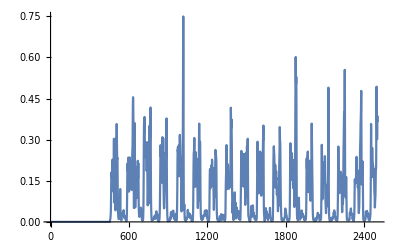

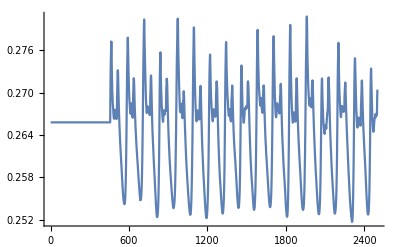

Sub03_(1)walk1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

Sub03_(1)walk1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881272.0.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881273.0.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881274.0.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881275.0.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881276.0.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881277.0.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881278.0.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.240881279.0.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812710.0.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812711.0.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812712.0.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812713.0.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812714.0.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812715.0.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812716.0.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812717.0.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812718.0.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812719.0.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812720.0.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812721.0.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812722.0.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812723.0.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812724.0.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812725.0.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812726.0.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812727.0.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812728.0.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812729.0.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812730.0.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812731.0.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812732.0.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812733.0.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812734.0.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812735.0.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812736.0.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812737.0.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812738.0.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812739.0.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812740.0.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812741.0.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812742.0.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812743.0.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812744.0.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812745.0.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812746.0.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812747.0.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812748.0.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812749.0.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812750.0.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812751.0.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812752.0.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812753.0.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812754.0.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812755.0.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812756.0.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812757.0.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812758.0.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812759.0.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812760.0.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812761.0.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812762.0.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812763.0.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812764.0.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812765.0.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812766.0.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812767.0.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812768.0.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812769.0.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812770.0.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812771.0.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812772.0.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812773.0.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812774.0.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812775.0.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812776.0.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812777.0.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812778.0.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812779.0.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812780.0.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812781.0.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812782.0.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812783.0.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812784.0.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812785.0.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812786.0.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812787.0.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812788.0.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812789.0.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812790.0.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812791.0.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812792.0.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812793.0.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812794.0.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812795.0.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812796.0.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812797.0.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812798.0.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.2408812799.0.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127100.0.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127101.1.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127102.1.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127103.1.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127104.1.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127105.1.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127106.1.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127107.1.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127108.1.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127109.1.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127110.1.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127111.1.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127112.1.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127113.1.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127114.1.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127115.1.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127116.1.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127117.1.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127118.1.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127119.1.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127120.1.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127121.1.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127122.1.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127123.1.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127124.1.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127125.1.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127126.1.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127127.1.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127128.1.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127129.1.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127130.1.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127131.1.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127132.1.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127133.1.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127134.1.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127135.1.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127136.1.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127137.1.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127138.1.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127139.1.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127140.1.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127141.1.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127142.1.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127143.1.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127144.1.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127145.1.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127146.1.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127147.1.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127148.1.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127149.1.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127150.1.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127151.1.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127152.1.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127153.1.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127154.1.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127155.1.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127156.1.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127157.1.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127158.1.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127159.1.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127160.1.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127161.1.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127162.1.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127163.1.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127164.1.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127165.1.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127166.1.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127167.1.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127168.1.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127169.1.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127170.1.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127171.1.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127172.1.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127173.1.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127174.1.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127175.1.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127176.1.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127177.1.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127178.1.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127179.1.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127180.1.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127181.1.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127182.1.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127183.1.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127184.1.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127185.1.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127186.1.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127187.1.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127188.1.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127189.1.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127190.1.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127191.1.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127192.1.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127193.1.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127194.1.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127195.1.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127196.1.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127197.1.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127198.1.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127199.1.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127200.1.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127201.2.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127202.2.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127203.2.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127204.2.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127205.2.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127206.2.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127207.2.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127208.2.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127209.2.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127210.2.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127211.2.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127212.2.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127213.2.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127214.2.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127215.2.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127216.2.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127217.2.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127218.2.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127219.2.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127220.2.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127221.2.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127222.2.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127223.2.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127224.2.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127225.2.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127226.2.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127227.2.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127228.2.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127229.2.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127230.2.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127231.2.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127232.2.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127233.2.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127234.2.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127235.2.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127236.2.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127237.2.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127238.2.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127239.2.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127240.2.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127241.2.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127242.2.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127243.2.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127244.2.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127245.2.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127246.2.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127247.2.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127248.2.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127249.2.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127250.2.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127251.2.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127252.2.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127253.2.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127254.2.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127255.2.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127256.2.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127257.2.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127258.2.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127259.2.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127260.2.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127261.2.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127262.2.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127263.2.6200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127264.2.6300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127265.2.6400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127266.2.6500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127267.2.6600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127268.2.6700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127269.2.6800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127270.2.6900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127271.2.700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127272.2.7100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127273.2.7200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127274.2.7300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127275.2.7400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127276.2.7500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127277.2.7600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127278.2.7700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127279.2.7800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127280.2.7900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127281.2.800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127282.2.8100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127283.2.8200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127284.2.8300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127285.2.8400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127286.2.8500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127287.2.8600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127288.2.8700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127289.2.8800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127290.2.8900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127291.2.900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127292.2.9100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127293.2.9200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127294.2.9300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127295.2.9400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127296.2.9500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127297.2.9600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127298.2.9700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127299.2.9800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127300.2.9900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127301.3.00.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127302.3.0100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127303.3.0200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127304.3.0300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127305.3.0400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127306.3.0500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127307.3.0600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127308.3.0700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127309.3.0800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127310.3.0900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127311.3.100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127312.3.1100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127313.3.1200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127314.3.1300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127315.3.1400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127316.3.1500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127317.3.1600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127318.3.1700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127319.3.1800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127320.3.1900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127321.3.200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127322.3.2100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127323.3.2200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127324.3.2300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127325.3.2400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127326.3.2500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127327.3.2600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127328.3.2700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127329.3.2800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127330.3.2900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127331.3.300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127332.3.3100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127333.3.3200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127334.3.3300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127335.3.3400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127336.3.3500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127337.3.3600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127338.3.3700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127339.3.3800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127340.3.3900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127341.3.400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127342.3.4100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127343.3.4200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127344.3.4300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127345.3.4400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127346.3.4500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127347.3.4600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127348.3.4700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127349.3.4800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127350.3.4900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127351.3.500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127352.3.5100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127353.3.5200.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127354.3.5300.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127355.3.5400.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127356.3.5500.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.3945755500.4194642300.24088127357.3.5600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00276723167113556440.4194642300.24088127358.3.5700.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00305592952262007550.4194642300.24088127359.3.5800.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00320730708245770250.4194642300.24088127360.3.5900.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00335512927794878650.4194642300.24088127361.3.600.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.0033800588907194610.4194642300.24088127362.3.6100.2657938100.3818287400.3946562400.2791308800.3057479300.5150693100.2803351400.394575550.00400442969025442950.4194642300.24088127363.3.6200.2657938100.3818287400.3946562400.2791308800.305747930.0017536864348980390.5150693100.2803351400.394575550.0056832952586481010.4194642300.24088127364.3.6300.2657938100.3818287400.3946562400.2791308800.305747930.00258269146230962570.515069310.0049687986984171670.2803351400.394575550.0083742490659394360.4194642300.24088127365.3.6400.2657938100.3818287400.394656240.0040995673921147480.2791308800.305747930.00323686849015524920.515069310.0068982896533366810.2803351400.394575550.0115381225137466420.4194642300.24088127366.3.6500.2657938100.381828740.0046129924811398710.394656240.0053337880650613070.2791308800.305747930.00379824730626440040.515069310.0101878136150461590.2803351400.394575550.014645154652761370.4194642300.24088127367.3.6600.2657938100.381828740.0055432757261920040.394656240.0066451446558237730.2791308800.305747930.0044454703801876140.515069310.0129610489215990270.2803351400.394575550.01563999458514210.4194642300.24088127368.3.6700.2657938100.381828740.00748163619546570.394656240.0081143797045152840.2791308800.305747930.0056322380422786780.515069310.0152716837907114230.2803351400.394575550.0155655379028459830.4194642300.24088127369.3.6800.2657938100.381828740.0096539544981011640.394656240.0085553674326685670.2791308800.305747930.0075028822132886430.515069310.0166022845861251430.2803351400.394575550.0185589016558007840.4194642300.24088127370.3.6900.2657938100.381828740.01057063734868910.394656240.0088320723033910190.2791308800.305747930.0081141732211491220.515069310.016783478819764710.2803351400.394575550.0243177280517100460.4194642300.24088127371.3.700.2657938100.381828740.0104480980628803510.394656240.0090409680588679230.2791308800.305747930.0063031147083019730.515069310.0164427132909463030.2803351400.394575550.03061092032045650.4194642300.24088127372.3.7100.2657938100.381828740.0078617422831166980.394656240.0073964579758051440.2791308800.305747930.0057011032843760150.515069310.0165809870682639450.2803351400.394575550.0340061598199581160.4194642300.24088127373.3.7200.2657938100.381828740.0082407477062454980.394656240.006665374222118970.2791308800.305747930.0060319264180918750.515069310.0154274256950568830.2803351400.394575550.034216658855914610.4194642300.24088127374.3.7300.2657938100.381828740.0091507926332821050.394656240.0060298316346001150.2791308800.305747930.0068835321633968190.515069310.0142626692120740430.2803351400.394575550.037897397479579490.4194642300.24088127375.3.7400.2657938100.381828740.0100712633673145560.394656240.0058826174415488390.2791308800.305747930.0082455322522312770.515069310.0144928276667293540.2803351400.394575550.0448081885500171560.4194642300.24088127376.3.7500.2657938100.381828740.0111670546521848040.394656240.00608989267020437850.2791308800.305747930.0099856122793730240.515069310.0161338553276140040.2803351400.394575550.055124794272084790.4194642300.24088127377.3.7600.2657938100.381828740.012547546081233380.394656240.0082068883700016260.2791308800.305747930.0106744701362429230.515069310.0202508893803311770.2803351400.394575550.056870534291821710.4194642300.24088127378.3.7700.2657938100.381828740.0123315392139649350.394656240.010190131274605340.2791308800.305747930.0114050274335168040.515069310.026086890259211550.2803351400.394575550.045205420520942910.4194642300.24088127379.3.7800.2657938100.381828740.0117995776930869750.394656240.0114561525532092120.2791308800.305747930.0131341464445134840.515069310.0307029643995476480.2803351400.394575550.035365354219169450.4194642300.24088127380.3.7900.2657938100.381828740.010962152551167980.394656240.0123472776300492440.2791308800.305747930.015770803713410960.515069310.032002493746748190.2803351400.394575550.035478379329526370.4194642300.24088127381.3.800.2657938100.381828740.009650451261529130.394656240.0154060910117162720.2791308800.305747930.0176133284728714720.515069310.030966394857054850.2803351400.394575550.037576044274117140.4194642300.24088127382.3.8100.2657938100.381828740.0080997021407321830.394656240.0214549139139541440.2791308800.305747930.0174366211820859950.515069310.0275992469881542430.2803351400.394575550.0352764220974555040.4194642300.24088127383.3.8200.2657938100.381828740.0066948653290962990.394656240.030605486666574380.2791308800.305747930.0180152559834320550.515069310.0244517155217375440.2803351400.394575550.034160734964268390.4194642300.24088127384.3.8300.2657938100.381828740.0068506386239858590.394656240.042101680947450050.2791308800.305747930.0210371013271356370.515069310.0240372761022326180.2803351400.394575550.0384207972959680.4194642300.24088127385.3.8400.2657938100.381828740.008709311255163510.394656240.053737843037134970.2791308800.305747930.0264390178998665970.515069310.026762072181914050.2803351400.394575550.042859795930897950.4194642300.24088127386.3.8500.2657938100.381828740.0121734609610393530.394656240.063543485154333610.2791308800.305747930.034070079840892030.515069310.035769103855553940.2803351400.394575550.0443882573591829060.4194642300.24088127387.3.8600.2657938100.381828740.0180028320394907860.394656240.070081845432198960.2791308800.305747930.041536011001763670.515069310.047445352581527480.2803351400.394575550.044408655918949020.4194642300.24088127388.3.8700.2657938100.381828740.0236205101829518520.394656240.072187941570310930.2791308800.305747930.041189286642390340.515069310.0530677415960369850.2803351400.394575550.043163378899078720.4194642300.24088127389.3.8800.2657938100.381828740.0250226830373502760.394656240.067423575325569570.2791308800.305747930.031962755687180820.515069310.05162939963223510.2803351400.394575550.0386704894826494440.4194642300.24088127390.3.8900.2657938100.381828740.0227847308844205850.394656240.055727864899792290.2791308800.305747930.0240847256965273020.515069310.047077341426779060.2803351400.394575550.038544619644524430.4194642300.24088127391.3.900.2657938100.381828740.018251297318388290.394656240.0419612729253325340.2791308800.305747930.024371471860315930.515069310.040799136060637520.2803351400.394575550.043201016024547850.4194642300.24088127392.3.9100.2657938100.381828740.0148553644786248370.394656240.032005596203134050.2791308800.305747930.029494891701149270.515069310.036826926613541310.2803351400.394575550.044072909734994330.4194642300.24088127393.3.9200.2657938100.381828740.0149477477640600590.394656240.0302718487593246040.2791308800.305747930.034109433668464150.515069310.037963973462882880.2803351400.394575550.0402701314914920560.4194642300.24088127394.3.9300.2657938100.381828740.0168554243166382930.394656240.0351649345774357050.2791308800.305747930.036943449200956440.515069310.035268556956273220.2803351400.394575550.0363953992533232250.4194642300.24088127395.3.9400.2657938100.381828740.0190928451942904070.394656240.038720099572022190.2791308800.305747930.038925047240000590.515069310.0299378125093991460.2803351400.394575550.0298947380927268580.4194642300.24088127396.3.9500.2657938100.381828740.0167383471409420950.394656240.0333260291874760350.2791308800.305747930.039435355485211110.515069310.027525892111174530.2803351400.394575550.0195621759009470470.4194642300.24088127397.3.9600.2657938100.381828740.0115453764388515220.394656240.025952416193639440.2791308800.305747930.035482438594696650.515069310.030082302866387170.2803351400.394575550.0115352483764027890.4194642300.24088127398.3.9700.2657938100.381828740.0078266222536477920.394656240.0217939645427247430.2791308800.305747930.0293053201743978360.515069310.0331324522999616940.2803351400.394575550.00753113346472064450.4194642300.24088127399.3.9800.2657938100.381828740.0067101641048421570.394656240.0173442935186025530.2791308800.305747930.024615827383249220.515069310.032855656437487750.2803351400.394575550.0061017422245683970.4194642300.24088127400.3.9900.2657938100.381828740.0090213995250837220.394656240.016050572698167490.2791308800.305747930.022124117971162920.515069310.032867346200101560.2803351400.394575550.0068713044664575630.4194642300.24088127401.4.00.2657938100.381828740.0128671477985070130.394656240.0224241923516520260.2791308800.305747930.0226012398587727840.515069310.031488453033586330.2803351400.394575550.0099928219914958840.4194642300.24088127402.4.0100.2657938100.381828740.0167845424125287680.394656240.0312634875772749570.2791308800.305747930.022352595228067720.515069310.0260759336597172560.2803351400.394575550.016433255129189360.4194642300.24088127403.4.0200.2657938100.381828740.0165189698430196830.394656240.035841505198472770.2791308800.305747930.0193718125626576760.515069310.0200743877978328860.2803351400.394575550.025859410746686740.4194642300.24088127404.4.0300.2657938100.381828740.015328560436937330.394656240.040804212112138010.2791308800.305747930.0149346562456102810.515069310.0151736999572937070.2803351400.394575550.034379134402102650.4194642300.24088127405.4.0400.2657938100.381828740.012655594978247010.394656240.038755720193178830.2791308800.305747930.011753473785103420.515069310.0128017643713626840.2803351400.394575550.03557838579789950.4194642300.24088127406.4.0500.2657938100.381828740.0136559753488339230.394656240.032000374160971410.2791308800.305747930.010853019213417690.515069310.012764018174252840.2803351400.394575550.028201118649975370.4194642300.24088127407.4.0600.2657938100.381828740.026111467599132450.394656240.0233749612550065920.2791308800.305747930.0112617412791317790.515069310.0117227079100977690.2803351400.394575550.0201801471126427830.4194642300.24088127408.4.0700.2657938100.381828740.05411513347795310.394656240.0192371410999524280.2791308800.305747930.0112861652485352380.515069310.0111983530192225660.2803351400.394575550.0180861976812356980.4194642300.24088127409.4.0800.2657938100.381828740.094835971942809770.394656240.023198562829437650.2791308800.305747930.0101305465400676130.515069310.0108540702898060420.2803351400.394575550.019597664304181820.4194642300.24088127410.4.0900.2657938100.381828740.14571833698705490.394656240.034612578078665470.2791308800.305747930.0086383927667855070.515069310.0099792009904716720.2803351400.394575550.0174875572958302050.4194642300.24088127411.4.100.2657938100.381828740.207077964195563240.394656240.0491399148059473850.2791308800.305747930.0084730988792605270.515069310.0093162967929012260.2803351400.394575550.0117142770739810940.4194642300.24088127412.4.1100.2657938100.381828740.27589110144813720.394656240.0678486263787460.2791308800.305747930.0093289286424014220.515069310.0104888554084173540.2803351400.394575550.0068201201431606250.4194642300.24088127413.4.1200.2657938100.381828740.359407332392091440.394656240.094333365690635250.2791308800.305747930.0107069388933508020.515069310.0132807176165594540.2803351400.394575550.0045151155322614070.4194642300.24088127414.4.1300.2657938100.381828740.444627041916472570.394656240.122338863885008240.2791308800.305747930.013600670080269550.515069310.0148333068891842740.2803351400.394575550.004131256634997820.4194642300.24088127415.4.1400.2657938100.381828740.484848775151135450.394656240.142404446025324430.2791308800.305747930.018413509816145210.515069310.0142379831134273970.2803351400.394575550.00382814926643483980.4194642300.24088127416.4.1500.2657938100.381828740.53653305539534890.394656240.15797044904617040.2791308800.305747930.0243955500703362460.515069310.0125714615426892380.2803351400.394575550.0039698524339465190.4194642300.24088127417.4.1600.2657938100.381828740.59150396061923170.394656240.180641291208302970.2791308800.305747930.0296986813284455570.515069310.0105076526969883520.2803351400.394575550.00443996729431943550.4194642300.24088127418.4.1700.2657938100.381828740.61026931656668440.394656240.22092493982367310.2791308800.305747930.0302104676754645920.515069310.0091717397334425120.2803351400.394575550.0053186731578001310.4194642300.24088127419.4.1800.2657938100.381828740.64627780216658860.394656240.29252771688956710.2791308800.305747930.0249676311526265750.515069310.008385151378063720.2803351400.394575550.0061396555608405290.4194642300.24088127420.4.1900.2657938100.381828740.66370231585240240.394656240.338896102336447740.2791308800.305747930.018072941481316350.515069310.00871720721305850.2803351400.394575550.0059438817719942890.4194642300.24088127421.4.200.2657938100.381828740.58731255065379510.394656240.30066636981806780.2791308800.305747930.0141327668848470950.515069310.010659151545305710.2803351400.394575550.00464520000326240.4194642300.24088127422.4.2100.2657938100.381828740.498652452400140560.394656240.22488788524675880.2791308800.305747930.014042983147244780.515069310.0120972602350980560.2803351400.394575550.00368573223023339020.4194642300.24088127423.4.2200.2657938100.381828740.464015041129931860.394656240.180492885723881420.2791308800.305747930.0154436973139692230.515069310.011894028930650640.2803351400.394575550.0037789803543574330.4194642300.24088127424.4.2300.2657938100.381828740.43363797606959330.394656240.17558598551735440.2791308800.305747930.0149843572919679410.515069310.0108005733246712960.2803351400.394575550.0040689168361901690.4194642300.24088127425.4.2400.2657938100.381828740.42714698339339530.394656240.219961399639777320.2791308800.305747930.0127888547934894140.515069310.0105104480500842360.2803351400.394575550.0042323405258931510.4194642300.24088127426.4.2500.2657938100.381828740.462524022596243870.394656240.264077575090587550.2791308800.305747930.0105747754953057040.515069310.0094376946341467820.2803351400.394575550.004065388313244470.4194642300.24088127427.4.2600.2657938100.381828740.46949929618253750.394656240.25226859455562470.2791308800.305747930.0090937201011761210.515069310.00858825815073530.2803351400.394575550.0040235855791739090.4194642300.24088127428.4.2700.2657938100.381828740.430373707103442640.394656240.22424832167184980.2791308800.305747930.0081473708113514160.515069310.007973671634194960.2803351400.394575550.0044211092312663030.4194642300.24088127429.4.2800.2657938100.381828740.399995273991813560.394656240.221819530127924440.2791308800.305747930.0074016144414931020.515069310.0072890011662275640.2803351400.394575550.005720776235546990.4194642300.24088127430.4.2900.2657938100.381828740.401609496657674870.394656240.233596068078153830.2791308800.305747930.0065212785131301030.515069310.0066622010272550730.2803351400.394575550.0077728807522734070.4194642300.24088127431.4.300.2657938100.381828740.39737446659965370.394656240.240756546666474090.2791308800.305747930.0049125853224073630.515069310.0064056093128807570.2803351400.394575550.0086201209539598330.4194642300.24088127432.4.3100.2657938100.381828740.44438820491146060.394656240.233845786439502660.2791308800.305747930.0033851345515928650.515069310.0063105083729894050.2803351400.394575550.0076366314156018430.4194642300.24088127433.4.3200.2657938100.381828740.51633454818080880.394656240.21854066843561160.2791308800.305747930.0034150500070566330.515069310.0064937309578945410.2803351400.394575550.0059693146407439710.4194642300.24088127434.4.3300.2657938100.381828740.481172169622854530.394656240.19328395762219010.2791308800.305747930.00359284515578142670.515069310.0068399966402253410.2803351400.394575550.0046396495488059060.4194642300.24088127435.4.3400.2657938100.381828740.346410323335794970.394656240.15880101469044160.2791308800.305747930.0032318234749306270.515069310.008345288834732970.2803351400.394575550.0042170325111724820.4194642300.24088127436.4.3500.2657938100.381828740.210752754347726450.394656240.131573012529537870.2791308800.305747930.0033108278902235520.515069310.0088755823327864560.2803351400.394575550.00471804330488761240.4194642300.24088127437.4.3600.2657938100.381828740.128376761955641180.394656240.119558280515767860.2791308800.305747930.0031535316229673480.515069310.0078178885350933330.2803351400.394575550.0050047808416431330.4194642300.24088127438.4.3700.2657938100.381828740.085885569627501780.394656240.118254556145426140.2791308800.305747930.0025015984400296740.515069310.0071549052846010930.2803351400.394575550.00482722460820185150.4194642300.24088127439.4.3800.2657938100.381828740.064587057372751850.394656240.129799120655198860.2791308800.305747930.00233485795692384060.515069310.0061836687691874110.2803351400.394575550.0045666046698507120.4194642300.24088127440.4.3900.2657938100.381828740.0526816664719009440.394656240.137876665231467080.2791308800.305747930.0022891620275026220.515069310.00540005562436867040.2803351400.394575550.0046779830701624080.4194642300.24088127441.4.400.2657938100.381828740.041342124616654040.394656240.122661204328386380.279130880.00279749294474470430.305747930.0021205678131247180.515069310.00651949535625141650.2803351400.394575550.0054336369662812370.4194642300.24088127442.4.4100.2657938100.381828740.033955675707641580.394656240.093870921919630150.279130880.0034628049205827170.305747930.0019791387205475260.515069310.00681964773773332050.2803351400.394575550.0065679922543531010.4194642300.24088127443.4.4200.2657938100.381828740.033604479097696630.394656240.072918665808681750.279130880.00364028349217932530.305747930.00203475464625291380.515069310.0071979763034559370.2803351400.394575550.0084178758095172220.4194642300.24088127444.4.4300.2657938100.381828740.0265187856116112920.394656240.053087594792899440.279130880.0038636301513609250.305747930.00203122445303822570.515069310.0075383732205971290.2803351400.394575550.010657962854439240.4194642300.24088127445.4.4400.2657938100.381828740.017563999623202910.394656240.045442431123076860.279130880.0045076292243059040.305747930.00268925602932343530.515069310.0075659384078548220.2803351400.394575550.012304395624867380.4194642300.24088127446.4.4500.2657938100.381828740.0178939045885936860.394656240.048089108052644640.279130880.00586449148683094050.305747930.003612508617340510.515069310.0089159070442735730.2803351400.394575550.0125307770164181170.4194642300.24088127447.4.4600.2657938100.381828740.020625074397616250.394656240.0414964767370666550.279130880.006112540038071480.305747930.0035911549265713650.515069310.0093482080209084830.2803351400.394575550.011741797621715040.4194642300.24088127448.4.4700.2657938100.381828740.0191590918376953330.394656240.030134994856770870.279130880.0056673602282832830.305747930.00368360135022275480.515069310.0091693478904613030.2803351400.394575550.0126090262182187650.4194642300.24088127449.4.4800.2657938100.381828740.0137330426932014450.394656240.017008217842979420.279130880.0054082355959166860.305747930.0049708574947432150.515069310.0086625738397234680.2803351400.394575550.0154972543306962070.4194642300.24088127450.4.4900.2657938100.381828740.007981011231191620.394656240.0087259990806000340.279130880.0052336118036628930.305747930.0063403841283213490.515069310.0084110832357980440.2803351400.394575550.017267756834256950.4194642300.24088127451.4.500.2657938100.381828740.0051096865447495240.394656240.0057369862147964490.279130880.0057594879456987260.305747930.0087197703119911550.515069310.0121445201022480820.2803351400.394575550.0162935374175334980.4194642300.24088127452.4.5100.2657938100.381828740.0046033119009878040.394656240.0045276526270360960.279130880.0078171649098272760.305747930.0130783625555736890.515069310.021648922366753440.2803351400.394575550.0143523146449397330.419464230.0079011039887337780.24088127453.4.5200.2657938100.381828740.0045915015658112460.394656240.004087484052236890.279130880.0113779469965513260.305747930.0194791729709470030.515069310.034548385839844730.2803351400.394575550.013456108045264530.419464230.0130009552657049580.24088127454.4.5300.2657938100.381828740.0044264738524817180.394656240.0042185707394280770.279130880.012113199767094610.305747930.020065349463822630.515069310.036942929057103410.2803351400.394575550.0120378625687883880.419464230.015706064425251180.24088127455.4.540.0061722155570663010.2657938100.381828740.0043441415071552770.394656240.0043924896997153960.279130880.0088072908105502320.305747930.0139420022785344180.515069310.026845711210208960.2803351400.394575550.0091702858031117210.419464230.012286165234196620.24088127456.4.550.0076857216487658230.2657938100.381828740.00435313135060008860.394656240.0045604748404762140.279130880.0063547190580724410.305747930.0093050029859676440.515069310.018122981983500790.2803351400.394575550.00766316693291224650.419464230.0101195839904518350.24088127457.4.560.0109658074973568630.268059100.381828740.0049381583464092080.394656240.0047070369887803110.276831390.0057114871186084310.305747930.006811954482756190.515069310.0135197514340765680.2803351400.394575550.0067510057318527920.419464230.0117350151493496230.24088127458.4.570.0133154511279175640.270248600.381828740.0052537128719232780.394656240.0048219291143002720.274533430.0052818007709447950.305747930.0055985837720174250.515069310.010381713651212310.2803351400.394575550.0052926003816471450.419464230.0105447078638562320.24088127459.4.580.019380456584003960.2720998600.381828740.0060030248729401480.394656240.0046805687448993620.272532080.0054713110251111780.305747930.0047241044554252980.515069310.0089997293227527250.2803351400.394575550.0042468462087006810.419464230.0091877229715838750.24088127460.4.590.0282185108171637280.273432300.381828740.0063399938732631660.394656240.00492478798130007150.271058260.00542057471233421250.305747930.0035425249286339980.515069310.0087153338967857330.2803351400.394575550.0035031474629907860.419464230.0093797843157250870.24088127461.4.60.036046524412413770.2743823700.381828740.0060445016731951640.394656240.00597874932230262750.269990260.0043689196601750070.305747930.0028348593709986210.515069310.0077608208392237280.2803351400.394575550.00332300745691317940.419464230.0097023225905128860.24088127462.4.610.056949764674049930.275256110.0053647584652198660.381828740.0060221562879365410.394656240.0076429847910862430.268995430.0042765012858720150.305747930.0039534361839424870.515069310.0065464106815694120.2803351400.394575550.00374233875468208940.419464230.0083402711827327120.24088127463.4.620.095301392327727260.276147570.0067767867606128070.381828740.005649260392923580.394656240.0092584637182487380.267967960.0040455269273940370.305747930.0057931332030467070.515069310.00524060602201895450.2803351400.394575550.0038127709353259260.419464230.0064080276583734840.24088127464.4.630.140817886051968960.276952270.0096943742094072820.381828740.0058104587429147490.394656240.0110057645245867570.267029630.003485219041114240.305747930.0080836474614177960.515069310.0058071637886864340.280335140.0054532089133306070.394575550.0034554765385038580.419464230.00749396858944253050.24088127465.4.640.17337826370219430.277221680.0124611414294518790.381828740.0070945083835462970.394656240.011878194935860870.266713180.0038269418964012220.305747930.0106889545272181240.515069310.00720582782894716150.280335140.0064820359816424650.394575550.00374297635527605150.419464230.00927908022699680.24088127466.4.650.180806145508419060.276813850.0138739827125428220.381828740.008364148837644910.394656240.0125321490754675360.267191770.0048533274401930950.305747930.0127407568987852780.515069310.0076837234973289180.280335140.009294251881594210.394575550.004315570975844880.419464230.0112742600435759670.24088127467.4.660.16864534129515050.27556130.0149308078775117240.381828740.0096303866860865780.394656240.01276840399465940.268645110.0057668505179703470.305747930.0141457720988181660.515069310.008338625472252540.280335140.0114752143656036540.394575550.0044119969637062610.419464230.012192520361851380.24088127468.4.670.161646622386551280.274162330.014481218880401280.381828740.0104476199787101860.394656240.0117819767500319110.270238880.00621692052439024550.305747930.0148343794082201760.515069310.009284024912301830.280335140.0123256570104438160.394575550.0038651104848873480.419464230.0108338388245586090.24088127469.4.680.176246883815392220.272932180.0122540025279387640.381828740.0089501970941465260.394656240.0101422804620650270.271614720.0065114492807457730.305747930.0145183840505376270.515069310.0099974652851594950.280335140.0138197855171216730.394575550.0034571841190853560.419464230.0103290741345360550.24088127470.4.690.182421882514024860.271955520.0091845725443938380.381828740.0078192125808625830.394656240.0079497715537529930.272690050.0066985323805070180.305747930.0131119050735452520.515069310.0097494934203082220.280335140.0137954989558154580.394575550.00334586351934502630.419464230.0101754149885554880.24088127471.4.70.166796963496877610.271098390.00710738255236016340.381828740.0073369418863527180.394656240.00587051312891763350.273621410.006406259702081270.305747930.0115557027622548850.515069310.008194906361520540.280335140.0117545157355322550.394575550.0034836112298951720.419464230.0099358385643666860.24088127472.4.710.16787681276027250.270315620.0063823621094468780.381828740.0086953725537594760.394656240.004275324990412520.274461910.0054442273932257940.305747930.0100918095332575910.515069310.006596126127513120.280335140.0093970469491176690.394575550.00351529772400037970.419464230.0098070880999724230.24088127473.4.720.203832249906530820.269791740.0060894057419360390.381828740.0130622283419316660.394656240.00355899148620303930.275019080.00510379770791233750.305747930.0088790379755244520.515069310.00616062238291469750.280335140.0082033831862774190.394575550.00390294558978374370.419464230.009542313887429220.24088127474.4.730.227321982127616840.269591620.0064433754149924670.381828740.020675411980325990.394656240.0034602278069075330.275230780.004649466613567370.305747930.0081328465425316350.515069310.0068326769476336760.280335140.0075809928306988760.394575550.0044473373618606810.419464230.0086247585877368070.24088127475.4.740.21797082641340490.26873230.0061845075790384770.381828740.0311205501813272170.394656240.0041404173477475580.276132760.00474159812985032550.305747930.007275691255985520.515069310.00632719084166419740.280335140.0077432182736839590.394575550.0044062333954484750.419464230.0066645994216905660.24088127476.4.750.189502141816087520.268554330.0071208842285339350.381828740.0429356003610666250.394656240.0074330583137847740.276318140.005159721437730190.305747930.0065462406121758290.515069310.0070199561315661040.280335140.0085037924401734580.394575550.0041220601269088050.419464230.0078105914804879810.2417753477.4.760.172248179969925560.268161550.0089916343887452790.381828740.0503139809815004650.394656240.0106528958075104530.276725520.0046527821404776930.305747930.0068747155838552440.515069310.008450176917299050.280335140.0093000948322238960.394575550.0040291036360727790.419464230.0112029858722878670.24246522478.4.770.160874966778904950.267981140.009705044674091410.381828740.053552027016392590.394656240.0114904953380242650.276911830.0051577031738998540.305747930.0073736955477658370.515069310.0100631067452134630.280335140.011363628460763180.394575550.0042274031902352950.419464230.0134798020719742550.24334421479.4.780.14573709808935940.267667390.0111339854556501090.381828740.049631580940106180.394656240.0106305329657093320.277234670.00582484302008910.305747930.0061143244430279820.515069310.0107841336930512960.280335140.0125530006961717730.394575550.00390155130632441860.419464230.0135595665063434050.24401865480.4.790.11915697272598810.267359710.010722456315881230.381828740.0382214618537981550.394656240.0092933497032389580.277549760.0052427482132396370.305747930.0049783824349561980.515069310.0102106643401667760.280335140.0113709538126904150.394575550.00339755976104383650.419464230.013545012821377080.24475556481.4.80.110359836614722350.267083280.0099505823518235610.381828740.0309408670231558630.394656240.0092119247951732850.277831620.0047928957793626720.305747930.0048221970781852240.515069310.0098633989342428520.280335140.0104456022323947680.394575550.003423418740749140.419464230.0132608729149240030.24555672482.4.810.13731653966359640.266802020.0091372675917931280.381828740.0402298126857530760.394656240.0112538483927550320.278117180.0052226334830641510.305747930.004261187376542970.515069310.009740583703565650.280335140.0088888583077648240.394575550.0038683342543882450.419464230.012435125357277530.24629677483.4.820.200865394610203780.266538530.0089269867218958660.381828740.062171184822072380.394656240.0139194721220106280.278383620.0051438711199387680.305747930.00334054050374703270.515069310.0079208903090149970.280335140.00794576113198840.396403940.0040577476714519090.419464230.0104491179804734970.24681965484.4.830.2745644888446230.266381230.0096318816028917680.381828740.075252179900339930.394656240.016930735191969250.278542160.0051900613365916070.305747930.0027372798281147410.515069310.0065273141003084720.280335140.0088484367322927950.398548210.0041877820815548320.419464230.009900158262624620.24752046485.4.840.303384279819624570.266308850.0096160813063674470.381828740.070264664701596620.394656240.019632227690673390.278614980.0053579093956299490.305747930.0022777765385992270.515069310.0060813527794538480.280335140.008841237931965910.400731340.0040300305787370080.422436140.0101634473044487530.24815762486.4.850.239687060121543280.266310560.0095786041160853680.381828740.077713222752389370.394656240.022023888134683460.278613260.0052949890484313260.305747930.00216557352691033230.515069310.00654498146475103550.280335140.0093682067926588020.40296020.0035241644991052260.425503230.0102069365939059420.24874196487.4.860.146985323524683380.266463230.0106188889290391550.381828740.090138159887685890.394656240.022853067725256490.278459560.0054909826255878030.305747930.00335338878670126670.51248310.0078019895687106380.280335140.0101313031001359930.405213140.0040719467635459930.428639440.0114133566908763870.24925051488.4.870.083887428601465070.266862270.0096282815617137060.381828740.085002079079703770.394656240.0208493411827338770.278056120.0050213613072224590.305747930.00371222566413456680.509844750.0091379586120620850.280335140.0095727244086636350.40748280.0052969194916640260.431822330.0111737979142323520.24971458489.4.880.070540173517840190.267149270.0089840906318914920.381828740.078791915083893950.394656240.0201645510157109320.277764440.0058433006283907960.305747930.0038288584892538710.50709470.0105539707719895150.280335140.011244949648142220.409840030.0086079116532666420.435105780.0105041436993746490.25020943490.4.890.10227060641325180.267375820.0108803509986431460.381828740.072117711019038510.394656240.01905807105901190.27753330.007582312799737810.305747930.0043024858043540740.504284390.0115667629129242880.280335140.0139601732326267160.412189370.0164850783892378570.438376450.0113571953236077960.25067395491.4.90.140174763114037040.267585040.0124460615144552210.381828740.052337325511095580.394656240.0147684194924537180.277319140.0093632508606428920.305747930.0040521415499351310.501446170.0128212021592500610.280335140.0181126677246570280.414490560.028107629218918210.44157730.0105136722304202640.25108368492.4.910.131231333597925580.267406920.013850108858289990.381828740.0310372284229773340.394656240.0117310225808063120.277501510.0113793507009806640.305747930.0039484595883307010.498620420.013859348387631220.280335140.02547677094697610.416764520.036729445962934450.444700250.0104268503515368360.25148827493.4.920.078295249288952530.267433760.0125302579259910060.381828740.0181525441935747980.394656240.0096024227547288030.277474060.0129477823066895190.305747930.0043728314354957250.495928630.0130770954293807660.280335140.034503142336922140.418880570.0365902257902988860.447593140.0101148520871894260.25185035494.4.930.048082644027787380.26728960.01071486019786530.381828740.0116607310771296730.394656240.0073951629634689570.277621360.0151402817074155480.303602850.0053488298425407880.493347220.0132283953005248540.278344190.044478841481021640.420911180.038774279193812950.450325550.0101450640460367010.25221195495.4.940.0471803755476512060.266882440.0083413689079640560.381828740.0077765519733771350.394656240.0060380888943801450.278035660.0163552925281163360.301636710.0065159255276623560.490947620.0153828597960047590.276518140.056670818470165860.422776240.051129774217775860.452813560.012276033907424160.25251831496.4.950.0432523091865009150.266641150.0057140154842611960.383010490.0046152486824558550.395265390.0051082443963234340.278279980.0167821570640503680.299788170.0091229672846512770.488756480.0205568735998034530.274795120.070408963430326020.424405570.06280933770972390.454996840.0163215718939060050.25271583497.4.960.0421402149811059140.266453760.0054369103739354560.38404410.0041093817564752270.395756390.0047732932936682860.27846910.0185860626452906160.298084720.0120765645213583140.486742670.0290877368341299520.273197750.078704947671536380.425875750.066097354762037260.456948930.0242147063912087140.2528902498.4.970.0595239337858372440.266435740.0067174544177233030.384774690.00420148093875551650.396021290.005136704831215440.278487260.020629761006484280.2965150.0135532987291665380.484919830.034053103816964630.271714430.076226264122442880.427187780.061004212776381650.458680380.03769186888807640.253051499.4.980.086221390794228260.266481280.0079217053813149650.385089420.004398245912615060.396166320.0066267794903135020.278441360.0230955657355291670.295166310.0143017833785363860.483343350.033133839135419380.27042890.064490105133852870.428346280.0539939494264289750.460175460.055627568405879410.25325473500.4.990.13144022311313550.266580010.0090550457057826520.385274280.00514208191778782550.396203090.0083260094767478880.278341740.028586559792167320.294092690.015432981878478890.482081210.032940218885524610.269396720.0533034993778128750.429306090.0500686092042660350.461376770.076127689820893370.25351019501.5.0.204894301349158950.266435050.0109310512222457140.385589870.005891676097327120.396429190.009818275555609380.278487960.039728775388948410.293482180.0175315731365320930.481208420.03607013357098210.268805780.0440131704164545350.430057370.0463979838374418830.462269130.095273854635748450.25382497502.5.010.281232243545231130.266358350.0131691464167980560.38576790.0072287806228368540.396550820.0111441311232657120.278565190.057198919072561890.293117540.020026661959031570.480719450.039529046778805310.268451320.037671267147810620.430509960.042794252674720240.462770080.11262115606564250.2541416503.5.020.30388222391250880.266355170.0133337899854227730.385783320.0085247764936386710.396559210.0116319320132930330.278568390.078708274031821180.29307320.0213392937298853660.480425950.042052905011063010.268408140.032740361730686780.430853020.033831710004585430.463137220.128783223824239980.25441009504.5.030.291956166359865770.26626410.0130606272601953840.385821710.008747630199103540.396629560.0126278023739883650.278659970.100624799331299470.293290480.0210997721671335250.480982910.0435246908483833060.268619570.031372514129559940.430437770.0226373726310274620.462560770.142417384223218370.25449561505.5.040.323151402632880560.26636230.0146063371346832220.385611870.0097467104240032930.396479210.0157520624670346860.278561210.117393262932047830.293691450.021059055626572870.481478870.046010411068063340.269008680.0353150305756021530.43012950.0199414657363076630.462100810.156146942248055450.25469618506.5.050.357187042589484970.266389450.016571067864193870.385369450.010999128938087030.396352660.020308643580385220.278533880.12358699022612460.294478690.022176111177328360.482286280.049802259225865650.269768810.036278407469479060.429661350.02560146690247160.461412670.175884314476121350.25488073507.5.060.32720850737347570.266696510.0172725299251309420.384825860.0116803649190134470.395923970.026442968457950.2782240.118577432319869950.295297570.022600033823262230.483295480.051994453886098290.270554530.0312404486116128480.428994330.0325661604945197340.460468620.205661065534341960.25507689508.5.070.273472856170730360.267864980.0160764823269372130.383365630.0133157380642109320.394586980.031962689413739590.277031530.105895337399025140.296077010.0214776135021303020.483879940.0487581365433045340.271298190.025650241762012350.428807580.033764760999663090.46005980.24090719327725930.25553777509.5.080.246925303028269980.269391080.016250296384081470.381559580.0173529374644427680.392880190.036845052775852390.275442310.090341998442702580.296626930.0208507660579416370.484403870.044063500357015790.271820630.0212593571922293880.428575910.0282153887875660340.459617450.27233678819648360.25599433510.5.090.229631484647994020.270245730.0189561858569561070.380273810.0212709824635160940.391842360.040805801056375040.274536490.077944528658309390.297392030.021988537456733260.485311310.0439404853377345150.272544720.0186403056494769470.428046480.021755661967546340.458768590.289509363853856060.25650905511.5.10.233278336290759110.271160510.020706068172200760.37874280.0214029140312262180.390674940.040035021456819290.27355430.072035999335530770.298453040.023646921014397080.486669450.0439591864990374060.273544110.0170128661464974370.427160540.020334094504773590.45744270.284054647417777860.25705245512.5.110.228008528760565930.272081210.01926580755247440.377150230.0178882858007398320.389465880.034969674057138550.272552510.070102529670863960.299594020.0219806100588242520.488174970.0401555023866642450.27461360.0171583521902713980.426107480.0260023461414104030.455922790.25466312846301280.25752245513.5.120.173617910975420120.27275310.017355883234067890.375848740.0148421132132706050.388520130.0273857960361857770.271813020.067183633864694170.300683580.017535331761964740.489679430.035490576791979530.27563080.018825925498007910.424971720.035676062663946130.454345190.20752539287218020.25781482514.5.130.106097589883369690.273112910.01714691550666570.374979940.0145195474452452740.387939450.0206931543268476930.271414090.066110066975710870.301597390.0144072265766829620.491108740.032327911080530940.276481570.0209203759456004540.423722470.0433729364372752450.452736870.153111743356268950.25773219515.5.140.058966805943571680.273161850.0161793261491303230.374532460.014975243835333030.387725430.0173451255169206480.271359670.072413778900362520.302368220.0154532727691667970.492479960.031141897203826410.277198030.0224414358918326760.422432920.044521333091495850.451136220.102330378638516850.25744846516.5.150.035646118344611350.272827320.0128982431407274870.374553170.0137061967047760640.387946380.018850296371170170.27173090.081966757916223470.303070010.0185885110574720050.49392480.0297673569375772920.277849670.0208488790383762750.421007120.041722955511442660.449389830.0623297553414673760.25710938517.5.160.0271198345015376640.272106390.0110044663370308260.375031220.0131351501075001910.388597560.022473808259877570.272524920.085941514182795480.303722950.0210527288461344680.495457220.0300869553262036430.278455630.0167109419686275150.419449580.0394167844132216750.447501810.036038025664674120.25669574518.5.170.0217669274554826150.27131650.0100637702728717040.375652120.0126075135155399830.38934680.023328458142658570.273385510.079864034746593520.304233010.0233884670233823230.496957530.036156209102373190.278928910.012821318192459240.417816610.033264382776620760.445575890.023999140070536390.25615293519.5.180.0154402210420378110.270507910.0093891147349892640.376357350.0102507801724384850.390129460.0206955800170798150.274256330.071684699978211570.304604690.0239908035459709120.49836790.0432837840121097560.27927380.0117059955386131870.416183530.0214240981005518260.443703630.0220510495465094970.2554736520.5.190.0113335958375694380.269696910.0093983239677564270.37710370.0080019919420287620.390870240.016834925154783720.275119480.069480973917775160.304886880.0219857154126334160.499646760.0417581961103028750.27953570.0129685367632218270.414631520.0110019145934849760.441959510.023990375226061250.25473886521.5.20.0103154833611404910.268916910.010912128849544260.377845750.0077740978472129080.391604740.014186216293323570.275939960.065854543404674570.305097470.01846616264250090.500754470.0332904341325723840.279731160.0139174867685805840.413222840.0060091996732197930.440407810.0268411381640709620.25398576522.5.210.0103341846289115670.268189740.0134086963882335230.378576670.0090133798091091220.392325450.0159485163866820160.276696360.054699353010215490.305207090.015892711380592020.501655950.0251002389756280270.279832930.014284137150368550.411982390.0047971193570374180.439087320.0291960549844316460.25319897523.5.220.0101811461074070490.267541720.0155443707448443750.379267590.0108196031404183750.393004190.0223170525812917860.277363540.0411877663796047650.305220060.013991901435144270.502382620.0194541436545624740.279844960.0143558362536294220.410886320.00451138869962762050.437962760.030508258345303980.25240196524.5.230.0107303505601019450.266947820.0152223115070693260.379946260.0128034686793923950.393668110.027014278212352130.277969310.0294305616217537150.305137830.0130911213750683970.502968680.016862143988600060.279768620.0140856848338830450.409901120.0043861552987223270.436990290.030355813876581930.25160772525.5.240.0118330228086816510.266414890.0133027430994089970.380573640.018589704126793340.394280790.0368781490264053840.278508270.0208288616900119020.305022370.013470824731992750.503482180.0155221036216048910.279661450.0133802988743990330.408996870.0044112606628459250.43611640.028451629207723470.25082515526.5.250.0128635298449859130.26589050.014513506968989380.381186720.028918195268642030.39487980.056412399850582510.279034340.0158374374791957940.304910230.0135018415044990020.503919680.0137468419736604950.279557360.0123876304736925160.408202880.0044355057658264890.435362320.0248294640007498540.25008839527.5.260.015083254505335150.26536090.0177022136520190.381788490.0359161025708781560.395468860.075202163749424190.279561380.0124260328709133120.304823360.0119438025477390420.504314090.0122637409960078690.279476740.0111107180649047450.407499650.0042646873262384350.434692930.0203430761819581340.24943004528.5.270.0194007518825859950.264906270.019844209799113140.382338870.040949910664505410.39600540.0833259564100360.280010380.0093198838129824620.304679390.0096274952185713660.504741850.010862703290046380.279343120.0107792341191360680.406741950.0038563964099609240.433966290.016256991862003740.24875431529.5.280.0283276254706270050.264471250.01835514349170650.38286240.056948705715105730.396511860.068440754243329250.280437090.0070874933398952490.304542810.0080142465504116560.505178040.0093056739038871130.279216390.0106378149605488790.405994530.0035449205125107180.433245670.0130125426747693550.24807813530.5.290.043702249301537470.264040190.0149300698208379820.383368560.085356925035511180.396977970.0466568092514869840.280857080.0071123143973731670.304426880.006987310931212510.505655820.0092075569384338050.279108810.0099173102307056880.405225790.0036258150211617470.432492180.012632475822866620.24739051531.5.30.07744553057867080.263618830.0120018837739593060.383859130.119265161779794720.397430140.044729526381111740.28126490.0085643378511679160.304317250.0075544256140575040.506164120.0090136930580546230.279007080.0080529559310274870.40443120.00408028421043955550.431711420.0116913623450348660.24665811532.5.310.11579179240455960.263215150.014194450740763010.384334880.160531656772159440.397865390.055321784549262670.28165310.0126361532250071020.304197150.009388992923468520.506667190.0090236764707418180.278895640.009923502266036160.403642960.004319995880515830.430943310.0121364593926248150.24589514533.5.320.119644111088171310.262826870.0197414640064533350.384803510.192269674552491640.398287930.07490381501692230.282024170.018943412915149590.304056750.0111815316614491470.507197110.0097692149170612260.278765360.0125369274395041970.402801360.00383658518276734160.430133690.0142480040378624230.24503162534.5.330.083121365407867160.262446270.022472185390748840.385285490.186074196319601980.398711650.087697910030309050.282385710.0239989645461375250.303872030.012289411846546260.507701940.0112149918192562990.278593970.0134098656143250280.40195850.0034828187266428560.429340850.0143699504261179680.24411333535.5.340.0440254428633836060.262073860.028190131640182570.385775320.204127936473332330.399132510.088302983986222770.282737360.02349873810273230.30365250.0118111393565341750.508188260.012852547329583680.278390260.0160117123243964970.401112760.0038739182518731450.428558560.0147406242177188980.24315275536.5.350.0238871829275691850.26171730.035802496357184040.386247130.30547238532665050.399535020.098673102992688250.283072110.0180585497603854560.303433180.0097688275632920730.508661210.0105480987957518050.278186740.019882044169409030.400277040.00369342251686381180.427793820.0143153805962183190.24216373537.5.360.0164307471087130550.261364940.037944488153055210.386714380.400136301865157860.399932660.113840596362876290.283401050.0146611232399526060.303210910.0083767037812035330.509097160.0080211441945539590.277980460.02366361369275780.399494350.00335182715828208530.427083810.0146203284541025560.24121185538.5.370.0123798067511096140.261019110.0368139330854410640.387170180.40016101461713490.400321160.118160404322119220.283722110.0171368800594341180.302994720.0096549343679580550.509492990.0073156159429339010.277779790.023350841692668470.39876840.0030961871840274880.426432060.0148952460275039340.24030065539.5.380.011644031205047670.260689620.038763878128555320.38759910.392812440234472040.400687590.115247118477861120.284026340.0253200414793670270.302795930.011641124280890310.509855590.00737125955272926750.277595230.019544909499970290.398105930.0029241157556767510.425836540.0133924821420663540.23946542540.5.390.0091897166783929850.260362580.042845957514437460.388009380.40541515433068130.401043910.116714395333580840.284326720.038152615780779910.302625730.0122471956878208720.510198550.0087588987216710070.27743720.0159595126290467440.397492790.0031820591665877960.425281870.0118980698480855260.23869268541.5.40.0054164762605255380.260033010.041685069639732650.388407220.40283042729282760.401395920.130144750307743080.284627830.051289259151344750.302481820.0105748850673783020.510521720.009557227014827640.277303550.0127038784435842860.396924940.00386167403401143070.424763610.010676461885971920.23798844542.5.410.0061926508357910320.259771180.0359265228219721460.388735460.3796897343770720.40167980.149182838585457560.28486590.055959987026326810.302341630.008312201295264670.510762770.010957797353669590.277173330.0112004516601485750.396467840.0052067817760240640.424356660.0111458592547784770.23739255543.5.420.010693013845348980.259370670.03336490174886460.389176540.374325123335050470.402087640.15752677659834580.285228130.047742409626445180.302243270.0075169198653814170.511115440.0128297597452697730.277081950.0110428522192341070.395883540.0067660309236103930.423805870.0113158793335726830.2367251544.5.430.018540539464320040.259045180.036608984106078310.389542990.390328837739719160.40242190.16211705593316130.285520760.033317164210423190.302144750.0082894233463316130.511388610.0132148440710293490.276990410.0128997686361476580.395407160.0077952967130347790.423362540.0120791392467678240.23617137545.5.440.0259999355497251940.258699080.041873412472653190.3899240.394961207034834950.402773230.170476275386003160.285830240.0214901162099456060.302054150.008845255507863040.511655210.0140126905744898040.276906220.0150061561325811870.394937870.0077157769476692410.422924020.0134766904672531090.23563753546.5.450.0269853835818253050.258338370.04366613316322460.390309030.394769617525488340.403133370.166268159406890240.286150910.014926034937831620.30198030.008445755567115260.511929560.0133021627516759760.276837580.0168025363648745050.394466990.0069529861559621970.422477650.014647699383209690.23512508547.5.460.0239171069630498870.25798130.044165156266595870.390682140.4299514403553710.403485620.16866511704153130.28646650.0111590932706634920.301919940.0070783589685699920.512211330.0113969008401645020.276781480.0205880993524008540.39399270.0065603173820637490.422023050.0143895233236904750.23462685548.5.470.0244114635301977620.257638650.0541034395702776550.391035430.47303694581113030.403821220.195871525568253520.286767590.0085683031171449870.301868490.0056320555228288220.512502210.0112737713568817030.276733650.027866299140155070.393511820.0074932111752881150.421557040.014111127429961560.23414271549.5.480.0285576474035684930.257338760.076878543893709110.391353140.54449775922004980.404117790.24388834351969020.287029710.0066174023763337580.301804380.0044158478218043230.512755420.0107083043427617690.276674050.033894614896388990.393077680.0099560234847600340.421137940.0134325213680136140.23371529550.5.490.030636560611213720.256964270.10069275023495480.391734320.64046304959106740.404480520.283807868339513770.287355230.0058419388952579730.301752020.0035621248781385370.513112920.0082074734241145650.276625370.0335102765547544150.392491440.013700476256635610.4205720.0109631302920370230.23310008551.5.50.030991057606299140.256654430.107678637944645310.392062080.66111113477298710.404786060.287396190772287450.287623020.0059132065839719030.301681710.00340048019343816350.513410020.0069358057199245840.276559990.0277453419146496340.391984440.0173107279307354830.420086550.009628687172336370.2325685552.5.510.0289898197078131550.256355610.099040296007455770.392384210.67800727458270130.405081970.27835299020601640.287879970.0051110096413225570.301599780.0039386285681317410.513700550.0063121312400497040.27648380.0212067808536838440.391477810.0194833921314693130.419605840.0092887437902595610.23202084553.5.520.0293931702235148170.256064050.098407740787542370.392700530.70088667246116910.405371040.273705096059119140.288129460.0054087558739175760.301513760.004991423873093060.51398460.0070571451217155310.276403780.01709801639856280.390982410.0204620069061785160.419136340.0101528398307844120.23148281554.5.530.0356969396760507960.255788980.106037398938485820.393004370.65559674865656570.40564530.258281562974031040.288363730.0068170350315170540.301419950.0045941630426590630.514249250.009013239241131690.276316510.015877042664687480.39051350.0205514393487491630.418694730.0093897417800075190.23096517555.5.540.036480396198852650.255534240.103471913045321650.393291080.59435023280069180.4059010.241873262132059540.288579710.0076673635052670180.301320810.00319150226314586030.514487720.0103332664793501470.276224260.0182275682907900860.39007840.0196306500491047650.418289840.0101490327203392050.23046641556.5.550.031831355805785810.255294550.098247487717542440.393565970.491600750422247660.406143130.22143407554606240.28878210.0099275350544036250.301215890.0044115266554054850.514694110.0153183979149787030.276126610.0259612890878924660.38968650.0185334874007994470.417930370.01964462312968740.22999954557.5.560.033934362081782550.255079340.100962420646491720.393803050.3738082351048340.406356340.203555214365686350.288963120.0101450858020118280.30113980.0043554662161415580.514895130.0165868940747351150.276055770.0261358132437473770.389336430.0158975141212122050.417598690.022859119385478520.22962353558.5.570.040117214908780650.254890520.122569260235416270.394043510.327680678721274770.406555810.212717168913833440.28912140.011006229838600120.301007450.0044140585218043350.515051190.0172182354328137380.275932540.0251142760464834780.388987450.0131496033001863840.41729570.0233377785424363530.22914497559.5.580.0426546757052887540.254723640.16481156311309490.394250920.350481051020140.406729840.242285270929109180.289260870.0099567126641492680.300899770.0043937132107271210.515220450.0163650215024364820.275832250.0249669547444231440.388644750.0111392191135391680.41698770.0217193934420768820.22871365560.5.590.0335116609469613140.254572520.1730131334119480.39443920.36420035015389620.406887380.232917900343315030.289386840.0081839427695571540.300800680.0046124058248641190.515403370.013557821598058030.275739930.026509673922885990.388289270.0091413791312064950.416665070.0171949581284317030.228271561.5.60.0215336764200856280.254454140.1252401204378870.394601040.307769015593120370.407016160.19107394539706140.289485290.0071857521601702870.300693880.00356856652470714750.515596760.011062661791577140.27564040.027855858731747980.387904880.0076780156643270180.416319240.0136995787356695620.22777575562.5.610.0173917576095097520.254349310.0778444781345480.394740340.223261993725735740.407128510.152793305764919730.28957230.0058886714714680840.300606980.00248561946533877850.515825740.0091305813286310270.275559390.0245776699267652230.38748910.00755759777514365860.415936270.011581541983266120.2272616563.5.620.017718974365422350.254293010.0593663635930964450.394845480.180745146079208360.407200380.132636253245596360.289618970.00524318215245153650.300499340.00243664229280273450.516078460.0071282034774263710.275459030.0180462967317032670.387010060.0082199353020316020.415503620.0096228400703125670.22662592564.5.630.0158065099917425560.254243520.047272645498191910.394937160.17319738883493320.407263180.12926934922098820.289659950.0046911536062717850.300406040.00251129425656798850.516374120.0075203211628614380.275372010.0128084895297067360.386473530.00779798592432258760.415017560.0079534214467025780.22589102565.5.640.0146628961994972950.254228740.032393265661778160.3949910.143855215835286460.407291950.1246817730224760.289672190.0042597842478086550.3003250.00245971031800758030.516701360.0080242016732142530.275296410.0121594287677398750.385900640.0064918385911839420.414494380.0082343006009933250.22510941566.5.650.0159636622952379660.254252470.0308223510543880750.394985070.097556481607820520.407276280.110107902551628990.289652540.0045798977059450790.300293370.00193048406664953470.51708050.0086364382071341910.27526690.0123342109304556260.385293490.0058850486122384470.413925120.0097853376904903380.22431414567.5.660.0180073023122193050.254290720.037600937343253880.394941090.054472112041184910.4072380.088736051515608430.289620860.0049534319311505920.300311570.00177994755568725120.517490530.0082707424013610550.275283880.0107398746381805410.384696920.00555367202651372950.413348040.0098989025030875760.22358659568.5.670.0216106085530062660.254406050.052646232825887770.394800620.032854141076788060.407119530.08581413071234080.289525220.0045599244613863350.300382030.00201692555357938170.517925310.0076242421282150080.275349620.008357775332169790.384117090.0047066000946161030.412772930.0083674928012431730.22290715569.5.680.0221056620998805950.254560970.078886003764858310.394586720.027543555932668370.406950570.086455895272985010.289396450.00274342614577622460.300526620.00231931787197758040.518334520.00604739525112551160.275484470.0060342862712378720.383663420.00419834303658667050.412294750.0057190457948300570.22244587570.5.690.0190313466315389060.254767230.103186714042135960.394285160.0248433235243795230.406718660.078592328271680260.289224480.00147586497785125280.300751420.00252759727952832270.518767830.0043080295391034780.275694020.0044323793388766470.383263120.0050960806686671180.411842590.0039257800406864590.22211644571.5.70.0160440422396106280.255096490.09773391920220780.393818270.026766031656482980.406352730.076978625575406980.288948710.00202576128235342450.301077990.00272433635861935460.519068180.0044255400157367120.275998220.0039121027153173590.383200080.0078180330134845020.411684110.0036464891948271530.22225234572.5.710.0133340690069563860.255498390.066902435319367430.393235640.024960301964885670.405898920.070277236135747230.288610030.00268060113847865250.301496680.00329517555867588380.519491170.0057976963320673160.27638790.0057780244492052820.383049040.0119112395896446180.41141710.0039782007406708640.22232466573.5.720.0105371909353585880.255999570.038535018505672620.392506830.0161083796882895320.405328670.050077601025240680.288184470.00284820598672543440.302014960.0036560886414737180.520010740.0067834823377177430.27686980.0094089140160009510.382837970.0164612681309228780.411078720.0048521056685208630.22227342574.5.730.00806808020420930.256622740.021075195413657270.391625360.0092473095608869830.404624880.0286610648748540.287650320.00278066442617924770.302598170.0041521690306499730.520581540.0076385755790119290.277411610.0135194253000646140.382597130.0195810931925435060.410703640.005007097239736130.22213564575.5.740.0077758909394047090.257395820.0107208626088431840.390563550.007304084508006770.40375790.0146670490531718850.286979940.00283407039005164260.303241870.004755022784798830.521237370.0087891789692836150.278009190.016849736583413950.382273020.0196629335751192860.410234060.00606231051509278050.22189515576.5.750.0081295859162330530.258322630.0054148725154173330.389295270.0058957041444160190.402713150.0073172914877587680.286164860.0023688248660830350.303979350.0050188340590218920.521967560.009440052385154630.278693550.0167901939995491330.381907580.016564685525721050.409694150.006520701718719380.22165693577.5.760.007945251755491020.259385760.0043083881739044530.387825580.0046927980138407370.401433180.00425307840065295050.285214520.00183578527786523250.304820310.0057710051083096140.522799550.0101560657326859090.279473910.013735344325090640.381469870.0122598252537400330.409038710.0068439359640776250.22146939578.5.770.0054024493999811580.260561960.0040486856088182160.386157830.0041987145324793290.399817510.00380282503519572620.284143780.00185843205983612470.305787410.0065657077131852350.523745390.0101839083676824660.280371810.009532885912452110.380954020.0083547850694973140.408250170.00734543883386810.22135308579.5.780.00276042126738024070.26191760.00342114492691323070.38422480.00307191682559606250.397939090.0043135328800817870.28288430.00174859813030222220.306866610.0059429485230616480.524778940.0098514004186744680.281375110.0056895021678352750.380399510.0053746936587443870.407358070.0056773385813278890.22141837580.5.790.0040261321301149720.263360720.00359177586245970450.382096990.0029789867726756770.395866970.0048608230264522940.28151340.0019752696844419310.30807720.0047286539568067520.525846060.0092918413110949470.282502730.0036941084705322410.379890880.00342781114158877570.406459930.00549588258490410750.2215715581.5.80.0055243516761446340.264955910.00372466670500791070.379712030.00358694391244386830.393537450.0047137020434971420.279961510.00258042845623717350.309392570.004154280027940490.52694720.0080135922117860.283730610.00275563054979994670.37942540.00209173235529803860.405545010.005378242020119550.22189923582.5.810.0073526647339986290.266692280.0038201254457424640.377089050.00322757097696659430.390968050.0043326844165280620.278228280.00307795827886807270.310773970.00422734334814940750.528031060.0078812207890704930.285023110.0034693450252417490.379033790.0017225668971839330.40466780.0058703169304928220.22230394583.5.820.0156628737639308640.268520020.0046167132300481860.37427720.0026398335865915050.388206680.00449893547440961050.276353820.0035227041395977510.312204940.0043959875478232330.52908450.0086122064018039780.286365160.004390765249211180.378716070.00205748553618933940.403823490.0072415320690050950.22283932584.5.830.034965787522985920.270333270.0050932063049770630.371371270.0029553508602946770.38534540.0052307502864655120.274443070.00366536352436275860.313700840.00458555080753530150.530115330.008502396112642890.287771430.0041586745823026880.378471460.00215390500015869230.40299140.0069302327295667570.22359623585.5.840.067535468709592790.272152550.0048650251149236690.368359260.0038875206730882410.38237140.00586753437544970.272474320.0033420060580387140.315234380.0050573303940131660.531102880.00744348388793961750.289216780.00374247517650616070.37830190.00196894509155565950.402178190.0059793571703770960.2245831586.5.850.11303587125933070.27363430.0044846514635339380.365635030.0046617946326894080.379667620.0069147002977936310.270832370.0030984617469607910.316804520.0049822383024306050.532044490.006225650036330760.29070150.00298979973058207270.378210420.00177468720486118080.401393080.0058989131958381320.22576629587.5.860.163997733263112040.274637070.0046038636041126740.363332760.0054529448397215020.377358770.0091090201894727040.26970150.0029770444603363510.318482110.0043141450830571650.532968130.0048757516577396350.292294750.0021576925630384090.378195020.00165892663650976830.400622690.0062188271424446180.22707436588.5.870.20133158694775910.275578130.0051886025409742720.361022020.0060856514549621240.375024410.0130432624000875580.268625740.00303243928259805050.320215930.0036472800900049890.533858380.0041016992000030820.293950720.0028243064073852470.378262120.00173023339047877550.399880420.007195034425157550.2286203589.5.880.213418171384763630.276578780.0060283912369983990.358615660.00636247403474818950.372583130.0166318543798246420.267466420.0031532610632644980.321934440.00356105879982701120.534678110.0039879374096743050.295602470.00336379470787605060.378383610.00172509286326634520.399211270.0076066939321601680.2300801590.5.890.201812745523353760.277449880.0071247736065706610.356362960.0064499358067829950.370279840.0174523509153061350.266444230.00303142453372836580.323591490.0042484571043923690.535425280.0043210838623586120.297204790.00236256181759607070.378525530.00178260714988845260.398594160.0082743889308682480.23144562591.5.90.186110815607484050.277768590.0084075942358941490.354819990.00604271418476744550.368659370.0155012508298240440.266067220.00317430647145253980.325114370.0056260575596457430.536073080.00532372598950022450.298685540.0020497146541054650.378658760.0021232147736349950.398033590.0099708208833087140.23263314592.5.910.195581275142066660.27725270.008938225560311520.354333660.0056027600315737180.36806010.0123809972650213240.266676660.0036036448096863270.326492530.0074545737284079160.536594530.0072818345088377730.300032290.0037152649732435320.378818660.00277055493115999740.397563420.0121665012211554340.23371037593.5.920.20551070588688720.276206150.0078744294613816450.354529340.00501890902124147750.3681210.0091969343178937550.267899990.00350696604279127420.327738710.0093237551036168440.536961250.0070329910301094930.301255950.0046585989430611210.379068070.00341194482768179560.397235810.0137731389602969380.2347892594.5.930.209920127247278270.275060910.0066235240798172470.354939710.00486148221179697960.368398040.0073467094876940180.269218730.00332627544398907040.328805890.0101164909705968310.537126430.0058266586240000430.302308870.0057709950793234390.379454420.0030967009486433470.397120280.0140466086368304450.23590754595.5.940.227585753057123920.274061950.0062642335926618180.355319710.0052473850798729480.368661110.0072855030256996080.270352040.0032502748032578730.329666330.0102792191906302710.537085190.0055031048616496240.303161590.0081515245315145220.379971650.0022838832368206510.397230120.0145939477211960950.23703375596.5.950.234994203406265760.273271950.0065851555779109570.355610110.0056234599483301710.3688560.0071511953367058910.271237110.00279334757223674350.330329370.0106999573649678490.536864080.0051281160239963610.30382120.0088232327775666780.380596620.00192824259102824820.397544260.0151676112010932230.23813589597.5.960.219133814029060510.272531080.0062440154443823840.355982720.0058588445644398270.369150080.0056326529734327290.272058160.00194451187672232120.330824210.0102940473050987280.536468860.004067196871740680.304315060.0063200320053409610.381348790.00175624598068436920.398072430.0133878963318608720.23923939598.5.970.171683978641085420.271743660.0051423305504484310.35653320.0053829984258933960.369636450.004153177879743660.272921330.0015855305824753270.331173650.008421983240548240.535909290.0033568582919759230.304664650.0043097403587558490.382235370.00147713019137935540.398815540.010188101478535190.24034237599.5.980.120377307813733040.270974730.0041110128001255490.357194550.0043200573523508510.37025210.00425063854872882560.273754830.00199579638616819350.331376820.0066909348057652080.535189420.00352932725189032940.304868250.0039785035433417210.383253320.00148514419746395630.399774820.0079093688616259650.24142045600.5.990.110445313292794150.27029840.0034179181080683620.357886640.0040745566881773110.370919580.0040023522835646220.274480290.00254158383928998560.331436060.0059939273072281440.534312980.0039175760683046340.304927670.004190276635672470.384400250.00158869223678251960.400947150.0061374146820720270.24247072601.6.0.125035537483420670.270101480.00280506392643165930.358171230.0044324964578540910.371208090.00293633137104266050.274690170.00250605115560225550.331367470.0059759376370394030.533315810.0043509787524927680.304858880.0042016260435771370.385636320.00176504593179189480.402282470.0047767928094466630.2434741602.6.010.15477223662552650.269327930.0032260085454454260.359234010.0054259974447520540.372279930.00329866061013929860.275508790.00204210129637753730.331148540.0064560566293188180.532101690.0045528690062075280.304639510.0037182987503712010.387091360.00165641544893173320.403922250.0041971070423856930.24451699603.6.020.195416546175007450.269009250.0047362938492442680.359911980.0086351427469155590.37299230.0053781302680592740.275843320.002365962340522770.330805690.00726268355261570650.530754740.0046944304434651610.304296540.0042831524167857310.388653550.00138567431419312630.405736230.0043719423729736420.24554362604.6.030.22235173526960850.268674590.0064488726078978580.360721320.0113343724216481960.373848830.0073649362613392080.276192930.00287544176706818230.33033540.008052030929679230.529279810.0040626886689067480.303827210.0043917882726175580.39031050.00136621728729772350.407716380.0038962360634293860.24651721605.6.040.229614956459922050.268423650.0064243997732156010.361567210.0147490220791833950.374757040.0084223016094643640.276453950.00246278178961715230.329716060.0081408908013460910.527640270.0033612703961433570.303210970.0039321718325535710.392097890.00192690818972665450.40990450.0041943909273068080.24747125606.6.050.234825348867622020.268160830.0058295090037136020.362544470.0252186484787687430.375806630.009061139596637190.276726270.0017831520773671460.328947620.0072577951134524050.525849860.00371008016811028060.302449090.00381598639405415170.393989180.0023277529709449790.412274070.0057774796187785420.24836887607.6.060.213464425269542370.267853170.0058386671982745540.363681550.035985409234135070.377022570.0098913375675502930.277043690.00134924914011724120.328026060.0055068099364643050.523983860.00327058174690793330.301538980.0025010774264028680.39588370.0021188251468727630.414715010.006370818587483210.2491362608.6.070.164773772933671510.267592160.00548989661414790550.364886020.039949279654159820.378312650.0114494569923536630.277311840.0016421181496397780.326930290.00365953660700292760.521939390.0039056469657477120.300461460.00183110896448743770.397904660.00155578130261600580.417355840.0066693370081825420.24988932609.6.080.161207002089990030.267360810.0049725158988664910.366163520.045151817652844990.379678330.0148138402363670230.277548640.00195512626143884120.325659640.0029665482038885910.519721690.005345089719075620.299217610.0032496019143203590.400042450.00123514293250829260.420180350.0080704092231064630.25062745610.6.090.16807260218432970.267163360.0057445461322854720.367507060.05926199546599640.381109690.0190148827768412830.277750080.00153786191774363320.324202070.0027286859027517180.517373740.0048311996582045890.297797540.0038171671518237750.402228050.00142710237172060180.423119620.009360899505491850.25128023611.6.10.15199124712892130.267000760.0076486681128514520.368906990.070983771379677350.382593370.0247907373499955880.277915520.00194575994030738450.322562560.00240113677726787670.514894250.003778512169218620.296208750.0047657701494301990.404478260.0021384281661139060.426180110.0091214821707845970.25189446612.6.110.15608312683328560.267016140.009478424307498230.370211520.068820757678699620.383976870.028883580751403840.27789990.0028792422235323550.320739860.0024931147208281270.512369350.0033359518948070710.29445320.0061921927646322810.406684640.0033327573604093630.429253560.0068362528066656320.25236504613.6.120.176053763937277170.267077310.0106424306348165770.371543410.067355639214210710.385375460.0272877369630381080.277837690.0033149777413634060.318762150.0022050909790559140.509689480.00340320180463658460.292561530.0090234143530022080.40902610.0059014867951526790.432512530.0061980384564384320.25286071614.6.130.19850249542756550.267097540.0091858410054557850.372967750.064814900034017270.386847290.0238157951175152270.277817110.0037085999393515090.316653840.00174290564135212950.506889010.00388677130471404850.290558770.0148143215381522430.411472180.0111023762731652380.435909650.00583324959350432940.25336696615.6.140.221205348432636870.267688950.0047132027667422960.373849180.049434576902841180.387764430.021443067062206990.277212520.0041886387815440950.314342130.00138314745534396750.504050770.0040450171242055260.288375350.0229965055883153170.413842920.020017980401414870.439264990.0048610441081927140.25374114616.6.150.192390779175988370.26812870.002403355862534330.374884410.034216701167456290.388803550.0210013120248759840.276759480.0056052943404915010.31189940.00185639885685903050.501082940.0043168595484139250.286078340.0342211721685945350.416287610.0330117885058822740.442688310.0050846689474999630.25414223617.6.160.14656674907606570.268300180.00235323738553862770.376166090.0266936527258552560.390051770.0177055666375788530.276582010.008605658675260440.30938390.00374271805251476630.498065980.0047215860130940090.283722510.050518241107191050.418723750.048996000146307960.446073820.0074483079761994120.25451775618.6.170.13039626314773710.268473510.00335774694512455070.377377180.016838958287427470.391196610.0108631321157345240.276402160.0127134859984727680.30686780.0057442117528847870.495070770.0053356049619935870.281376220.066519590313307950.421107090.062314251628329420.449353190.0110820631760008330.25487613619.6.180.128937667780632540.26839140.00650490600421225850.378738150.0088944619281772770.392441060.00630445419042129950.276487420.0176390610573369140.304488010.0069408932694481620.492194550.0074238181495716150.279165530.0692200735077620.423401350.065754837378552640.452455530.0143957951370515050.25522573620.6.190.116378352147172720.268140940.0090831910087410750.380137180.0052728077052095240.393191790.00639786190316282350.276746830.0230856659961737670.302309010.007505034061247260.489508460.0114434515052770880.277143030.065260800595457160.425538420.0597192929119829750.455303210.017866004885666110.25554448621.6.20.127482402739458570.267819210.0088906566752129850.381458750.0052560451855786170.393918590.0074973709608695190.277078640.027794715047510650.300376540.0077885490437775440.487087840.016515958321759880.275344490.066555971934531490.427445790.048859153076409740.457815510.0230912224792913650.25581204622.6.210.144019803155421950.267498160.0066316276623232390.382633130.0059348568076169420.394560370.0074458428974445490.277408160.0310210963899639060.298695590.0084992061675387180.485001480.0216054585988838430.273771890.066175781335914380.429035430.042005347351249090.459913560.0295617160580083260.25595287623.6.220.154849187556837660.267167230.00463434049116910350.383687720.0050459644147273930.395144840.00611148791645956850.277746140.033161643617294650.297252510.0101887377659881930.483252430.025403396762815450.272412910.060416718274751990.430306430.0403562749168403440.461610910.0380074206514017450.25600913624.6.230.193669920087733760.266942360.0063162919653747140.384362390.00442603509451255150.395561830.00632210662954180850.277974850.035527910618948330.29604630.0129362151475145540.481850520.0279490136633855670.271268960.052366089472846270.431280780.035217237764336250.462926020.049167521982779910.25601822625.6.240.248121421538697650.266748940.010410549525267420.384781270.005093934348319270.395874890.009668953875186830.278170950.039096690756156370.295255980.0158159485540449520.480774040.0303893500263277240.270514740.0437237547034023540.432151610.0252113828859885540.464018070.062049254811248050.25619975626.6.250.26867536514603480.266592120.0135792608255172530.385099030.0051455694557049540.396114410.0140890024406242990.278329510.044553105531547760.29468740.0178467111983389820.480038970.032714527910437850.269969520.0357806770401936160.432710110.0152156076878834710.46473010.077027042649961380.25631091627.6.260.27043431867057480.266585010.0157444701195735350.385121230.0046769474400419310.396128990.0190735880118372180.278336690.053099566342522360.294632370.0197315597558907520.479718110.034034501622024760.269916630.0314745596373127850.433075730.0100729325850517980.465126890.095128553123175820.25657607628.6.270.31979406936282650.266513790.0187600153257184470.385156230.0055913473303999330.39618340.025554561333148850.278408580.065162182986187980.294784550.0225078751117582870.480182850.036619684882457680.270062840.0300546340117458480.432624760.0096468696620378140.464595860.116492784790294980.25638081629.6.280.398048896768612050.266449970.0202160767957638540.385110340.0072829871872056840.396192720.033597304846279680.278472920.077978304327071090.295212180.024254189424604410.480904710.0423292632525045860.270472820.0286866155237021640.431947320.0118619096696996520.463800330.139977339286672940.25611301630.6.290.43986488756393670.267057820.017735989503072870.384236990.0106193258572022610.395439670.0420766221973023140.277857520.087321727184035230.296054690.023568556483208570.481699850.050989978107786720.271276940.02446920365422730.431505210.0145366223705461850.463133180.164168192463736180.25631539631.6.30.454915938820424360.268702840.0161715011492570840.382180950.0184468058862817360.393568520.051830327104219910.276163490.091233335606723090.296944910.0234562679720390.482457570.062697396280151860.272121940.0212012969590563770.431165370.0163990934583560580.462535490.185939730839754820.25672173632.6.310.44605337634862730.269788840.0207656229669103760.380427180.0307648299175985320.392217750.064687571010269920.275022150.091433655982199030.298115830.0283969489480162370.483451570.072627435128928120.273227030.0210822861233386920.43074470.0178012765030175070.461745720.199837633484803880.25738141633.6.320.40751980593378150.270166750.0282009800449112450.379293540.0421782045877683450.391556390.076771126658268160.274620680.091065894572740310.299580590.036568884347234530.484878450.075048844758021870.274601040.021561235281694630.430062030.0209864680653066570.460529410.200652782980395520.25826437634.6.330.359648348471613140.27091560.031750260848647780.377722710.044438688439483170.390462920.07777105884797710.273818540.088832764873501320.301066950.038143419075932810.486437420.06831137317636290.275987950.0208283199977119670.429250390.0239618404745271870.459126360.185132610452443360.25918732635.6.340.27917613047586560.271468350.0277378387070966080.376382150.036113356406476950.389567260.063867999173731440.273220830.080438235431480380.30249350.031321797791320670.487970660.054881578181833810.277314390.0205189425268746330.428396890.026417950405582940.457685990.155007509426976890.26003549636.6.350.170334577421968420.271949890.0196910154330516180.375286780.02484173651823910.388803660.0448668099804215850.272696210.06728784846480010.303570340.024579163920082260.489333310.0395341313549317650.278314020.0221380409591115620.427464430.032507551967881610.45628190.117049421488017270.26050567637.6.360.082331163618367160.272029880.012913255154270630.374750090.0189147287191514840.38851940.033149378024063430.27260870.0591394014693634940.304426370.0245943214376916460.490614170.028998365597391390.279108330.0255455138535842470.426422940.0401166483342068340.454866820.08120825458306240.26057292638.6.370.0505480250581770360.271740720.0107554873758837710.374651970.0192601611033645580.388482740.0341825071233918050.272924530.064795674199012370.305228680.02736449414251090.491872260.0264065537502887120.279852960.0257578723915297160.425306810.040062917048501750.453431640.058865266878633630.2603544639.6.380.072171785207768980.271412030.0107627802701426180.374667590.022461366839054220.388517670.045843081879630970.273281950.076752455625321940.305890380.0281161610174924840.493152860.0292801321834173060.280467460.0213467438888116020.424045470.031565249980645220.451893870.0587056473753414450.25990263640.6.390.130049058352428660.270812620.0109506409857040390.37505490.0254827483351303670.388910330.0571958225457806640.273929370.084725135525632540.306413440.0286995769144398550.494435330.034638229093501710.28095360.0165758219035932570.422682740.0210111668402429180.450287440.077087970469094450.2593139641.6.40.182413741764781280.270045030.0106206461016094770.375697670.0242355332965355640.389548790.0558165343987099060.274750230.087965172480893670.306796060.030457109160042330.495695410.037911975266042150.281309470.0118247149450016190.421242540.0123466833587232220.448639580.103801855194243150.2586162642.6.410.26560518713226430.269330750.0118143883206239760.37635330.0208652567407115570.390196540.046982166724712540.275505820.088512717435223710.307033180.0333917733595525540.49689450.037599008365441950.281530130.008719162828842170.419776160.0073276932568020350.447007290.129528770434723130.25783788643.6.420.360868923376225670.268677940.015792871809036360.376990850.0217912321460140140.390824650.0449855005659766450.276189440.087719455516540770.307169250.0347170760482020.498015950.035240733372542220.281656790.0076205381706748480.418335860.0051098842722642780.445435150.146130018612853190.25702423644.6.430.337368368239429230.268050340.01831745362705260.377649480.025526699508297530.391471710.046744856886986560.276840430.082309474399115910.307207510.031792373862369710.49901540.031759708368770270.281692410.007089633274199390.416971110.0042254079951747070.443979660.148686583109494480.25619806645.6.440.21117821897834950.267452730.017151188995234740.378308690.026597787262317050.392118240.044325802949317290.277454650.068691313153308740.307177260.027044644305690320.499893980.027681151856231710.281664250.0079829767581204750.415708250.0044790603354706410.442658850.136992362916197820.25538732646.6.450.105863143327862520.266925030.0148492667263999730.378904260.022976241592625430.392701990.038577020297217580.277992440.0529374169808907240.307119330.0225106658266613880.500667980.0220016416991555520.281610320.0085156604221177050.41455960.0059112623973206570.441470260.11595555452150170.25463053647.6.460.057001725878041540.266537230.0127264969601331540.379355360.017661535416289970.393143720.033724215871386650.278384920.04085348934664050.307048180.018167078155764690.501474480.0158972582297000970.281544090.0071415877296764220.413391810.00760977556055224360.440245960.093326049170649280.253921648.6.470.052963693928250190.26602130.0109895913880547170.379968810.0139074878843006620.393743960.0304519770707871940.278903520.031063542184487710.306923840.0151505275482976650.50198410.0136767905839955560.281428360.0055364567203566060.412538770.0091316469411231920.439410770.076007575271306080.25322476649.6.480.072944939709848680.265541960.0096774532480848160.380535330.012222687584816130.394298490.0274043892641018530.279381670.0226724715388148570.306809040.0151032505719273040.502480120.014279250324767780.281321550.00477090239785238350.411728770.0111072301792306950.438610150.06715013930713230.25258319650.6.490.084086602617922130.265135590.0088163399706069330.381048710.0130300427726712920.39479960.0219227486904944040.279784290.0204115270069679320.30664650.01662802520052540.502952510.0156331051063865680.281170340.0053536787077104210.410921210.0129130620183929640.437824560.065785497059163590.25192422651.6.50.087956221963098740.264746240.0090694095601119970.381547670.0216080491570017870.395286250.0172745442806960350.280167690.027576354949077960.306473860.0169565142284624080.503388720.0152034763448640420.281009780.0066145313581240510.41015470.0144273864632280380.437090110.067656464366705480.25125845652.6.510.117651282875753160.264414890.0136853183617178660.381993520.040685173632298490.395720090.0297208283116653960.280492170.039708860079691030.306284520.0152772528463174430.503849140.0130765855815265180.280833740.0083871466718833180.409354720.0136669409767101540.436323840.070362138071009690.250551653.6.520.15697380695079390.263988950.01963238457153080.382506980.071183012478034170.396222140.056820388388601550.280906820.050252276177677640.306147630.0124541792379659830.50421490.0110287192609547260.280706510.0110487971815751380.408711710.0143152386518682930.435717410.072696243423963870.24992793654.6.530.157160536424037520.263648850.0230002797524250830.382955120.114867850877967890.396658380.08818251124550510.281235930.051451210776863250.305964080.0093740213390136360.504630090.0084492206839682940.280535940.0146234614590833920.407976830.0197765780229104920.435024730.074341630068394960.24922274655.6.540.132441836189450050.263249060.0278194292780887570.383439220.17816395888450760.397131490.115447753814288370.281620580.0418712386275067250.305824080.0069205408570454340.505045050.00545903208838723840.280405880.0188947908488546760.407277640.022970180618909590.434358970.074223564415496480.24854099656.6.550.142546233859885880.262932110.031371261073775610.383868950.274232896451499230.397548970.12751375454209990.281923820.0284426858523945530.305624310.006280426601522880.505458830.0044264969711858850.280220320.024965959029698330.406537230.019517491759505630.433666340.07110328714455640.24780433657.6.560.17200329650482750.262568750.033928013589038970.384327660.383306768755753150.397996060.138253600692423840.28226960.0171821549950710550.30545550.0066601773675204850.505928120.00531014486737122450.280063550.032528584204113740.405753420.0129936415163241950.43291950.065518267133392080.24703037658.6.570.180703852026164760.262244550.040540784788689950.384764390.43424448509372160.398420050.170589758230454830.282576440.0102804375896792620.305250310.0074017929097327610.506391480.0062859647565784010.279873050.038741430448128760.404950430.0083281517872324070.432164470.0596027293772360550.2462148659.6.580.194752664723299360.262007710.0461006156268951440.385126320.44901876213309750.398768960.21727153348817750.282799610.008690872545506190.305017480.0088482725553876460.506778590.00674210360370914450.279656910.04164969227392760.404225690.0064094215647616230.431505450.055352783359152280.24541091660.6.590.2001849820454080.26161990.051527975084073820.38564730.454193369199535350.399274230.253455479665263770.283163220.0118130335492510670.30476780.0115647374108237230.507322250.007838973490208680.279425170.0413879051386602940.403291960.0058821434697863710.430624120.0528298545425908150.24446583661.6.60.176682238024282820.261459870.055576429794407780.385906650.420508357734927560.399523030.2774001097644390.283312620.0173650468726835250.304579190.0141787673900148260.507680260.0098072557790289120.279250140.041654098931080070.402626780.0059862897646774470.430013620.049792873669512620.24374236662.6.610.126961311417308180.261049520.058222876443020640.386500440.44666667313007440.400014460.28841431752003820.283693950.0225375902768966960.304226780.0151267027859773910.508194920.0112389412961403440.278923130.050040933635381960.401645210.0072659359807773720.429127060.045150308523210820.24262384663.6.620.088820082708714970.260780330.06762857671627990.386913590.58827399504237810.400343110.31601066341462930.283942740.0239655575227661140.303947230.0142936466849667120.508595440.0108234925003918620.278663740.068905508418336880.400846310.00988756151174550.428413380.039909739796930150.24168994664.6.630.087443885707555960.260530310.079909455464785060.387308090.7084067644362580.40065210.359358434686354870.284172860.0201151254582134230.303664420.0116086491433194420.508911510.0089454426919491950.278401320.083572424276245870.400162030.0137519867443079750.427816030.0354419053947532050.24085597665.6.640.123445681396614050.260222080.081540033705600240.387747890.7274551566985570.401011680.35301219893837290.284455280.01517431804578840.303402220.0089252580041734290.509317440.0077538884465379070.278158010.081735214802431410.399352780.0183399974096349750.427089330.0329474256381330350.23990825666.6.650.193864514038460080.25994910.071327857719219750.388146910.64317417404245350.401333230.29932582903590330.284704230.0144183390640400030.303148920.0080656576472326570.509646750.0081147028575875460.277922910.06765928435465740.398657870.0216644356167810940.426472850.0310076991681635870.23908047667.6.660.223035633834413220.259691430.058469658506073420.388513380.476706200919771840.401631610.238838824272463830.284938210.0186754702373297460.302927220.0091930867419217060.509955380.009400877535581370.277717120.0526537626494790260.398018920.020607999234979340.42589990.0278592135763918970.23833736668.6.670.181406004348793980.259406510.050317216649964380.388888290.34228549157181730.401947940.205481415600586470.285195810.024594821644474870.302738610.0101324067281976190.510310730.009428870355798870.277542020.047236558610786380.397330340.0145433586363643840.425268640.023871513752707530.23756458669.6.680.159381567146333840.259126810.046923047922893180.389239110.313297044772838430.402250560.217688671438029560.285447520.0272430441590762950.302584780.009701117106133730.510662630.0079285446814771010.277399170.0540007490632025760.396677730.0102582303151595220.424659760.0204427236553390880.23686165670.6.690.189887422620586670.258842330.0475025306126175060.389575170.33011061165783390.402549080.26191860251931670.285702370.0240583171853800160.302466720.0108799645583731680.511025750.0069288585229278450.277289530.066532539560533650.396040650.010080777635288980.424053820.0172695161049362150.23620305671.6.70.214750544113709580.258547480.049080105470849770.389900410.30243511526003160.402848350.2953690233568230.285965250.0190907992316219980.302387340.0141624905542358240.511399910.0055621079781375860.277215790.07702834292870530.395422390.0103651464836924770.423454920.014737487095259160.23558386672.6.710.201163863323664540.258285320.0477310675477131340.390172320.220339824674504330.403106860.27277542246402310.286197920.0180203018455831270.302348810.0153954695291351840.511748390.00370657980858222830.277180.07835374747114380.394884180.009030400257998620.422918120.0126549010441817810.2350955673.6.720.140153181673630030.257959630.049698869362677980.390489990.159510998638070440.403419150.205869501493700060.286485590.0182212650999755140.302338120.0124818769653149680.512188170.0028386483032668150.277170070.066230738794481990.394222850.00679995240869027750.422260540.0110064446766300880.23445172674.6.730.078101007624758740.257683530.065265931864626310.390745470.203254024041658040.403677710.170660308636183640.286728250.015669608238041870.302354170.0086783684995228770.512603470.00295204475507573760.277184980.048990077035200850.393631530.0048170746435704530.421656830.0091140007413221830.23393251675.6.740.0455931924319392040.25740410.086902483448496190.390994840.298508614453610040.403935130.20044005896931130.286972710.012700989877991840.302386610.0072086417809614790.5130280.0028833102929167870.277215120.032227946710464890.393042480.0033678866335574930.421050280.0070291029237711970.23342562676.6.750.032101968314105550.257165210.089035348088818510.391191880.39041845365094210.404147590.226659995389045440.287180820.0099874585724951640.302444510.00657972223371418650.513424930.00358937691380427060.27726890.01889988922735340.392524620.0023561425857788320.420501170.00543199953763205240.2330357677.6.760.0238591121279354070.256869060.067861891353956320.391445440.447868103239619060.404415670.213717615925886560.287437660.0061644107930898420.302496220.0046732843636716860.513883450.004064908965979660.277316930.0110728645154751260.391897710.0021455084307499330.419858380.004565145509438450.23246159678.6.770.0195206837395569540.256603740.052468052970621310.39166350.40434664859026410.40465110.182548432723004470.28766670.0033088964132360.30255860.00292963565478961040.514308170.0037648106620335510.277374850.0084931157757738470.391340810.00224706329674426730.419275760.0048398149071059670.23199452679.6.780.0183955239244401460.256346240.0507091698278932250.39187730.330432268912155270.404880140.165204550335399020.287888010.00280771528295082440.302613290.0021842617962966630.514727190.0030656489984658750.277425640.0084047531931680450.390785360.00214290589312716650.418699710.0050556046169645710.23150614680.6.790.019681515269140250.256103140.048669505083291430.392074070.289296787758566760.405093860.171880355542214730.288096080.0033348778976179870.302673390.00179701817777007090.515145750.0027855152994369870.277481450.0086743945663413490.390241290.00192555851094148960.418131220.0049092961384798760.23104196681.6.80.0206862833354597050.255855430.0488040158485442340.392299530.26798254806133910.405321630.18834149686284240.288307230.00365458907688221040.302684520.00128886969310882550.515539430.00348481923994545080.277491790.0092886392955852030.389679670.00191562686918896160.417570290.0055979430421372880.23047108682.6.810.0214315961319416460.255632960.061674338351432580.392509970.27454418742750940.405529230.20216779455120020.288496110.0035568073802905540.302677790.00164683757382350470.515923940.0041837099346664460.277485540.0111223213073686470.389113230.00265795619323248720.417011720.00598570839834040940.22987463683.6.820.024103296332028930.255405890.089558438768912190.392729530.31509483488558630.405742830.2056093556948380.288688190.0029294633262743890.302660450.0026910569456516550.51628990.0039587897673800760.277469440.0123341615557274240.388565560.0040295919818650550.416474030.0056633625332789010.22929654684.6.830.02792633998582450.25524180.122364976871597920.392919730.38110895687705210.405910140.22122472867994550.288826520.00299091188205258260.302585590.00316570438775239280.516665010.00429120930527360.277399920.0124656099077607860.387930830.0055879572210508380.415878660.0067833552451263320.22853452685.6.840.031327455125175070.25508550.136092002284458950.393102520.4323937975181790.406069970.240015126348657760.288957950.0031379682943242780.302510510.00273155153463393180.517038880.0043319547449824020.27733020.0117863283872179250.387303450.00584495195574857240.415288040.00766362438050796450.22779107686.6.850.03346776817221870.254833630.121027000501271440.393363030.38015041080595720.406312530.229104392048471440.289168990.00328868639398897330.302454770.00235916579450644050.517387560.0042280419802701720.277278430.0113504453125648930.38674140.0055319569688599070.414749160.0071588800463415090.22716793687.6.860.037335187501910210.254863660.117803967742412130.393392910.28023213820035170.406308750.223005310991074070.289143880.00389322599771857760.302342140.00232820677108772430.517840560.0052605883904433120.277173810.012497713235026690.385944040.0065407100007211180.414016110.0065658666217008910.22613538688.6.870.0413190568213083340.254806240.134256258883289740.393480330.240889665949160250.406375670.237141066146510810.289191890.00382879069956361570.302274280.00232805220587679360.518265980.0066529741056021460.277110770.0151796301076397280.385249450.0093092567806221680.413360510.0069002024845523780.22529595689.6.880.047913994359476750.254818080.14782695409161870.393427540.2728447227779230.406347550.255851669226551560.289181990.0032250631365462590.302356430.00220275550505750430.518619650.0060732557598684940.277187080.018583821157598360.384800080.0128046010157243860.412904480.0063255960451521860.22479343690.6.890.0520099908468339140.254834910.16085162585338150.393480050.28109669796810650.40636010.277497111907266060.289167920.00302126877638606750.30222310.0020597757317891390.519157620.00445412687461606460.277063210.0234059226909006450.383894120.0150695049975756930.412060080.0054802415504725480.22367933691.6.90.051734915756291890.254902220.1560567063134650.393402130.240316045737893530.406291780.2750046321838810.289111610.00339570615000815270.302254480.00217800430386128840.519614010.0044606630217530180.277092370.0267181896198244550.383266930.0142133896433233080.411441960.005223823314725120.22296196692.6.910.0489896013516824060.255027850.142138376521737140.393249330.178183376137100030.406161720.244401482298308630.289006330.0043523691312903950.302327160.00221506396922882980.520084130.00506117685164824550.277159890.021416160198936340.382662830.010986941576830220.410836430.0052264275899660220.22228225693.6.920.0422480367789757750.255200370.143128476118114470.393031380.112892642759637620.405978730.199171559428515330.288861390.0043925006198099620.302442160.00179138959282716970.520565550.0053646878308880810.277266710.0142550968234296020.382088750.0080194670140461920.41024820.00448249294506433950.22166172694.6.930.034386106783070420.255474760.150811662884126480.392712940.08626562866287760.405698930.180002880981976170.288630010.0038294528185864510.302568180.00181896218782980110.520983890.0057578798589015580.277383750.0103011407973609330.381630190.007336477578671190.409773220.00415837198992738840.22114684695.6.940.0279850557472986140.255795550.14343144833484120.392321160.096052463585624570.405362880.181563044528486120.288358140.0054005313707569660.302751110.00243306994186499870.521407080.0070088003456769270.277553620.009094598332969620.38122840.0092268521473976030.409338180.0049392167001124330.22072216696.6.950.0226862081070310220.256196790.112186082350235560.391831090.108241044300534790.404941060.149642487199131340.288016020.0110696698526759360.302976040.00267254599755756530.521787920.0091498322186441670.277762440.0106610949735323030.380944180.0120133218544866050.409009110.0063739841227997240.22042347697.6.960.0176611306196918050.256716560.076879396234611760.391200730.102508603269397760.40439510.106718192187156670.287569420.0216836085530549250.303252280.0020310139252648050.522156410.009218284648459410.278018850.0117673318968675220.380757220.0141039230835526030.408764850.007072620196064270.22022268698.6.970.011933768243995680.257345750.053191210868596750.390420320.071894266657937590.403723140.06988516507379350.287023620.038333153428722560.303610490.00185481746692377260.52261510.0071236487410106310.278351270.0107741886590122910.380504450.0157435947308627520.408437960.0059086134923056680.21996585699.6.980.0077543526304799830.258079440.0361337772302206960.389483960.040095507414003680.402924680.049271012238769380.286379940.059993959849315020.304064970.00306940204786768130.52313020.0059589718332812810.2787730.0113151863466198140.380245120.0172364194972550250.408087520.00517732748791122940.21967002700.6.990.0068235504965297930.258939110.0218349014471459070.388382230.0208854748886833470.401975490.037254299476404580.28561580.080495494535938640.304587060.0039155312265753570.523747210.0056198815952755850.279257450.0114161050877464070.379882870.0172599582639635270.407619970.0054343665532913840.2192739701.7.0.0059195750812535030.259960780.0121408645872119970.387044430.0115222962977479860.400675390.0292090829625500960.28469360.091701274715150410.30523440.00375211418465377270.524449930.0045375113355697080.279858270.0109586948302039140.379496530.0151116237317292720.407086630.0047305931679981550.21894047702.7.010.0048076116185357060.261128770.0075505118343714010.385472370.0091152235412984250.399146920.0292663713419907650.28362050.08840271445112830.306017670.00378485668791049560.525254830.00310442666941531050.280585740.011232255531269770.379068410.0113027112199985370.406457260.00285162354871993730.21871106703.7.020.00628733151543238440.262426120.0077951754709740250.383666780.013673580447325270.397390010.0402376236496609850.282404790.071069508706082610.306950330.0035780786722706740.526178820.0029321323488119380.281453010.0097942418474085030.378584080.00702686299722719760.405707030.0016892205142752720.21860145704.7.030.0063847555662883480.263813110.0093403581538673340.381643790.0185265872528321070.395419540.052005541482559660.28107720.047571091602268380.308058380.0031437209760325670.52715740.00388874091023494850.282485180.0063008869370568570.378151190.0040573152084192350.404937170.00259281379441896960.21865295705.7.040.0055008612301106270.265385330.0093409841093668720.379321370.018984894329894240.393151530.058436405584649030.279537150.027816398058211910.309290970.0026920132002393640.528187840.00392665781997367150.283635680.0044714346543795090.377745130.0026570803293992450.404120880.0045705446904161340.21893983706.7.050.005188413158036410.267085580.008057883477272490.376748420.0168853630433710260.390632780.0577918571742768240.277829280.015687251922692960.310639980.00232914250168118770.529231140.0040756400094318920.284897610.0051021641311622820.377394280.002236368937261450.403303990.006898215316357910.21932318707.7.060.0063327895880250270.268969820.006480422233085750.37388590.0115773217435786520.387823740.038848650158268250.275884610.0092573053661594830.312042670.0025776711343341110.530232710.0057537475330990890.286212820.00619926885629070840.377143640.0028409124515107920.402540790.0072001210378483220.21989556708.7.070.0109331117637126870.27100290.00575129072576047350.370745490.0063754570909345460.384735790.0176169543978292460.273724460.0059217986497632980.313512790.0022981778187622380.531201450.0065651801471849810.287594470.0062324806635548510.376987890.00373665066563166370.401815760.0071420099136809650.22067784709.7.080.0227307465480556980.272983110.005953348731243120.367522170.004374840827519980.381558090.0090092643115853130.271558240.0039392605284073650.315075430.00207135277231427360.532186560.0068392986807607790.289066770.0053070563359113080.376874570.00419259684958443650.401053010.0077131998749449120.22171692710.7.090.045240828121528910.274387010.0054998884006089160.364781240.00342912122694443220.378836240.0071844285287100630.2699850.00308064355385880350.316788340.00236851335550936370.533220470.0062867672234665470.290686170.0047689010718021780.3767950.0046007709994142960.400224340.0077405274929004990.22298858711.7.10.084657978977539630.275511030.005827443339631020.362210350.0032380652024752930.376259520.0074633904710039290.26870290.00310656823442090730.318637510.00259357410106183860.534265220.00520399861273773260.292442760.0050371268937224610.376774820.0045360857026936910.399362160.006270026576603950.22448576712.7.110.151062046038122070.276797650.0091041220379683410.359374740.0045548735713029640.373406690.009985896362998430.267210720.00302075104969555530.320521060.00350850072655714250.535232050.0045465695276939890.294243230.0060272528151338090.376872680.00395584652291788850.398583170.0047189286603135470.2261416713.7.120.242078297009040130.278089110.0128675858532112540.356512710.00703892016916867450.370514060.0137553355742423490.265686450.0031545598743974930.322363470.004846688482996040.536070820.0044989264388320120.296016430.0068326295952770730.377106260.003299243431411460.39794750.0042089374331031850.22789715714.7.130.323698367576675750.279198510.0142372060039380430.35388650.009565681656398130.367840170.0155997939592605120.264355870.0036901082300866750.324103190.00621042313136445450.536720280.00399123523249519850.297701470.0074733627322254660.377476290.0027608777358711360.397502090.0051500976776731560.22957566715.7.140.35501542949692820.280083080.0136213320126964880.351598810.0100333723376073040.365490370.0149560247692771940.263280920.0044326708244412760.325674610.0080276139496573590.537187480.0046817656014529740.299232230.0086442580642762630.3779380.0024725035689483620.397203670.0072282409601448490.23128874716.7.150.33156180970329780.280339770.0124120700977801340.350171990.0084109988468432390.363974040.013508444384538340.262966660.00459103918119330160.327048950.0102192466063407840.537509390.0052391724675851830.300577910.0095377518172847750.378390760.0025613437429303180.396992630.0100352750949652450.23275289717.7.160.32572494765066970.279868390.0115297992388198550.349709450.0065727261589304130.363390080.0123181225376008170.263542960.0040701902426299710.328268650.0121550858049508490.537689280.004870712534761140.30177820.0088131754415653120.378885870.0027246652543103730.396886490.0122742472190085820.2341704718.7.170.373917523895420160.278714990.0104958579051175060.350156520.005219336386382920.363690580.010915251211971420.264938190.00308573409216334180.329335240.013308627653364170.537781790.0045028694738556550.302833050.0071531928568205840.3793510.0028003407153966320.396814040.0121712799065357340.23549411719.7.180.38289793117213230.277468420.0087906126838255770.350842040.0045892538648940860.36423750.0090423404971162470.266422340.00173311014125354870.330208780.0130845707563812460.537667570.00380949740688470760.303701070.005590350830946420.379934820.00220418588481017650.396962310.0099787319880825140.23675542720.7.190.35164843828599810.276457650.0077008338246110680.351408630.0058251380652687690.364692190.008160361571015650.267607610.0012783531012856260.330871670.0118556286099599230.537372710.0043477903567779260.304362490.0040576819411749660.380603990.00163484300590784280.397309490.009331112459980660.23792811721.7.20.30241029164849770.275630580.0068682289392894690.351920450.006904641689469510.365118240.0083019595084283510.268565370.00181316668697533440.331343290.0101093253257669120.53692570.004640913966491260.304834630.0044208712842059070.381340480.00156754573928704480.397833940.0099591500933197290.2389968722.7.210.25052929667709150.274829180.0057246467828064290.352547070.0072593127637216330.365679210.0087882465007316480.269483030.00213679959914097250.331652720.0081193567729502710.53634990.00400142377531457950.305145140.0056404916886175340.382143390.0017923631927715510.398521420.0105841642061072580.23998173723.7.220.239545035361671680.273981350.0047287122763515290.353362470.0090732679204791770.366446870.0089188145807573370.27044280.0020922709393334740.331815490.0068987199312384290.535667720.00317565834857647370.305308720.0053375550946001280.383001140.00227292583481880030.399352890.0112733694653901350.24087685724.7.230.269410502925453540.273117360.00429583267238288750.354331110.0128092825934554970.367387410.008389453179112390.271409130.00231181762669724950.331834240.0060264795252986740.534855490.0028810507892970810.305327580.0049531511139894320.383951440.0027359282787263590.400368060.0106646126069704470.24169746725.7.240.28904250838094150.272312060.00538806984072637450.355363360.019788563608052830.368412860.0075036996981553380.272299230.00227706482193237250.331713960.0047058799604127790.533935840.00282900655966996770.305206670.004885978277333040.384973940.00255297323873496850.401536990.0085685582702303180.2424516726.7.250.2801094392110580.271581910.0063785345455621860.35643940.0310839307076632850.369502750.0086353460929452320.273097430.00210626965218290280.331455530.00376133566297531550.532880490.0022825255544885710.304947190.0039559261615896810.386106820.0019917165012948420.402897770.0060725838326102880.24316515727.7.260.26566888279809880.270853080.0063712436718768920.357619770.042299709733070880.370711510.0123730117342312990.273885850.00195074414517128480.331078740.00339177837080878240.531702050.00191985414965607150.304569620.00383373167655426440.387347340.00180675559743276270.404432920.0049539796921530350.24385431728.7.270.27549107864861760.270151740.0064208758944844520.358876550.051786970176494070.372010810.0150592121796522590.274636670.00134765270951565670.3305770.00288011073181449260.530384010.0023060509851569560.304068170.0046817297848960050.388718280.00197471287640122330.406162660.0054502828336641550.24454219729.7.280.26587775636940580.269503070.00592459758063772650.360177720.058627758943758270.373367120.0160011218556939950.275324260.00114706975710525450.329948330.0021835731461545170.528917330.00268761761769210770.303441850.0046592413799330310.390228030.00190846491814742280.408092090.0055279016585740370.2452409730.7.290.23315223539699420.269081940.0048287950839405270.361340740.0550505829840812550.374600770.0179957110214305840.275767150.0021985921991950560.329176110.00202478672615284860.527235940.00323168821952136850.302675330.0042653327213788740.391952290.00159023654862046160.410302280.0045167350125905080.24601626731.7.30.241793678912971650.268539450.0050413126477444510.362726310.052320803389263380.376059960.0234400177486214470.276333620.00323067323625106460.328273740.00237106210247137880.525525110.00455496762896521160.301783220.0040717055503120560.393645640.0016545394685042870.412531090.00512809002183962050.24665523732.7.310.270559764665097240.268185990.0059388017178940740.364013040.050274041151359620.377429810.0290479562038719570.276700240.00374170147497922960.327211280.00246160311117951060.523553420.0062910911993042780.300737320.0048570755139816240.39560030.00197271279359679130.415085150.007911072872578430.24741633733.7.320.266357486647987530.267755570.0058179911757813420.365472520.0481481330548401350.378972120.032100324418807430.277144080.0043567634194391240.325994910.0023435704875178040.521544760.0075427613993357530.299545250.0070073555662622570.397509840.00192145900943639450.417643290.010465256482824650.24803966734.7.330.2156723561139150.267486580.0059579407660016370.366807090.054435548633783370.380388660.031133484083853310.277420010.0046994133648866880.324664220.00262628342400509070.51924660.0082747163471256540.298247030.0089036119160079680.399734570.00186487213674065840.42057550.0113410057354157890.24874075735.7.340.18579769554335410.267209270.0078655959454943280.368323940.061029478648942110.381990220.0263787652967742740.27770330.0050544586280069110.323050310.0032969590660095460.51691720.0097693162277780410.296680460.010743006303854950.401832250.0023250106402541350.423430880.0116774158256119750.24943189736.7.350.203449877027640950.267119810.0096858561946068650.369678260.062701559149601070.38342220.0220300207890645960.277794430.0053913913556967830.321328610.00364991894345683160.514492360.0113573269882753950.2950190.0117648546362011890.403999520.00268189602465899140.426402840.0113112067887863030.2499958737.7.360.25746736157833530.267249140.0104409890706751150.370873430.063332758932060060.384688140.0226793900504464080.277662650.0060847039891175590.319456010.00325780606949661360.512016990.0118353721462423410.293223640.0121633297536031440.406161480.00313685008240398430.429409420.0113460196557902870.25049562738.7.370.291012516562608460.267379990.010125080453743650.372113540.060791538392682850.385983170.0288737519516921140.277529040.0060932556210561520.317468490.00332166459292653970.509409350.0115823965491395360.291331150.0113991559695737040.408448460.0038633822117696980.432577910.0128265469034208910.25102477739.7.380.257643027412817470.267301530.0093513935339039260.373584010.047752839759549010.387484190.031470140579784610.277609180.0029342378743079510.315396160.00243754808222854160.506673830.0070703926015214440.289369510.0079054086622735720.410847720.00334979048547820370.435882410.0072385802552623480.25155322740.7.390.202253408496023250.26778750.0076631185869146230.374528870.029203323462282730.388447380.025884933511579830.277111250.0021349315423327280.313089360.00290068169469381380.503983050.0058498432370757680.287196180.0060590437658737110.413049240.0049123161996778670.438998680.00512104004078515250.2519459741.7.40.13959466438461440.267998220.0052276402352513170.375722460.0145313540609024950.389625670.016341391819031210.276894220.00234823754359513370.310720330.003180761937715620.501174060.0059328256071459980.284972870.0050667535902501160.415325380.0084206073158343660.442177390.0050300801430194140.25234495742.7.410.083647693809360240.268069070.0046413173345215580.377013490.0078858668851270760.390869130.0094319644205931690.27682110.0030979027656444410.308322310.00294936538030911040.498366220.0054504525621223790.282731330.00574403896232455850.417550260.0133710596813098670.445268630.0048577034396812370.25270474743.7.420.0602898049036816250.267960010.0056900582475577290.378418060.0052691137980593580.392193910.0065255771133929950.276933630.0040929970120372960.305968920.00263947633591334230.495598730.0050804020520979630.280540440.0068252841515547650.41972040.0201993841382379980.448248710.0049448337626953520.25305835744.7.430.064550649713738210.267946510.0062754588628631410.379653860.0040214794154136590.393103790.0053788011586622770.276947540.0049592890133475080.303655210.0028760042039413690.49294490.0056802604385302240.278392780.0077838405649080450.42174530.024487567817966930.451021710.0065556835706215950.25334012745.7.440.080154430065163580.267761550.00621770700702010350.380967850.00372540468023408250.393763650.0050788438407927570.277137940.0058053110216178360.301478490.0038397617422558710.490393510.0063777699309472470.276370980.0092745043632037290.423680830.0210838763755903030.453633240.0071781520944055160.25360171746.7.450.112513910567386170.267567470.005640704397877890.382185710.0032709467115190050.394354050.0053444812394957560.277337160.0071232869265944390.299455760.0054170930026790380.48799880.00582118154158319750.274484260.0109275033825471150.425462960.0163004692785381350.456014170.006556739704187850.25381532747.7.460.142409009962011830.267390090.006049847337359460.383283680.00233545563101546660.394856510.00632949819110775050.277518720.0084499908119440950.297595370.0063946227059889260.485798980.005469876473873960.272736650.0146684126854318040.427046220.0142515652761100710.458129290.0065260547334558640.25395731748.7.470.150903731109850670.267358950.0081944338402025680.383966430.0021874235097773070.395150620.0072531882606484480.277550540.0095599516442935360.295866010.00645910200863270350.483797490.0056419940751382110.271097250.024379248044099670.428416420.0195841838570015480.459984610.0069011036816478050.25400948749.7.480.145080810526424130.267483250.009022277977466520.384258510.00233742833669633260.39523230.0069679288518945630.277423420.0101368210710671130.294286510.0062847320033124810.482023660.006624976745709570.269583690.0403157406654861550.429563970.035798778915390930.461564480.0083239041352919950.25397696750.7.490.119273557132280860.26753860.0067746820440363830.384551920.0024310101625228620.395333550.0057937537545763140.277366730.0097340705939079760.292959920.00663210524834950950.480522490.0069399297591911880.268297740.0585783329672793160.430507760.0567717297281477850.462868960.0086249526088240550.25393299751.7.50.08545299304279780.267498410.0044804978952902330.384868770.0025488453267727970.395487580.00403181687950071850.27740790.00869906780521670.291925740.0065444344199625230.479347340.0065571865637022420.267284240.070714923757066030.431226820.068363517585923750.463865620.008406916540518980.25389484752.7.510.066741788858300110.267424190.005159154376991580.385141860.00268226984481194620.39563790.00305155553072938330.277483850.0093095181782893150.291192170.0064159649885664720.478522260.0084519216883666370.266558750.073733059298493260.431703010.063415869923863120.464536350.0111076264848425640.25386363753.7.520.083206099009359850.267330020.0069314522099205240.385359220.0028670163504499960.395777390.0040881978221376210.277580090.0127080491505044810.290752990.007696235220157530.47803330.0144849291927141850.266121570.072533987410831390.43195410.050255484763476760.464906410.0164544862290243970.25384132754.7.530.134046924027950350.267323170.0084831018458005340.385379060.0031938988900597420.395788820.0060059901637185810.277587090.0175571927847471870.290705730.0108166899557275880.477742190.0207444983877240650.266074390.067477483602642930.432287630.042436045078669830.465261750.0262724175894914030.25412317755.7.540.203277042525824070.267137370.009888664734851420.385578820.00286622414908430530.395984190.0086041895198517140.277776560.0235346982249133480.290701580.013881732448779630.477983190.0207280718719405550.266070250.057739369201576380.4318960.040885564037043910.464868230.040952694503678590.2538894756.7.550.28390874851185150.26717070.0118368662338055130.385479460.00218166564556682240.395927470.0126987070998753030.277742610.0313852208022938960.290941840.0146463093286238070.47826350.0156782782501016450.266309830.045669973291137280.431725090.039656032242563050.464616550.058328599490332130.25400673757.7.560.351562977675460130.266941240.0129458682483981710.385556930.0020879914429834310.396107680.0174205860687649680.277975980.041152328456992760.291574160.0140283384319270960.47896010.0122475585474249440.266937250.036376594702222280.431255620.0363745651878534460.46400310.074268924024164030.25400897758.7.570.349839377115675140.266848730.011137867679590630.385461920.0030734407828126470.396129050.021114946134179080.278069840.053061860209848510.292307730.015555791578781420.479709570.0143964430975743570.26765980.033265590251617080.43081960.032997170043315020.46338270.08809325402463180.2541352759.7.580.29905557690063510.266824220.0086223787191455280.38526560.00320150491097294250.396061580.0254458550271622830.27809470.06690679676057740.293147120.0192763928923503670.480616020.0211861560501363340.268480120.0351477086368507040.430268620.0298111120247571970.462609110.101168971238383490.25423313760.7.590.290128444651255260.266900080.0085787481426022550.384941740.0029333125257944060.395872390.034239256309124310.278017770.080913671381469420.294063630.021428952962687650.481575570.0315222419615013160.269368660.034981328166482140.429727550.0243509745752813270.461807960.112286702813826340.25442337761.7.60.31962662169923940.267071070.012038509606444530.384503890.0048086230259161280.395571480.045835200761064770.277844040.091464009461671260.29500740.0218274442077433380.482556830.042323034626805340.270276650.0318710040991306360.429201350.0196615317556544760.46099450.119398688404496430.25468552762.7.610.338713224955411230.268269120.0174113022211139540.383064760.0098991618925067350.394230020.055321211217447140.276614190.09582528631380670.29557710.024740738506333820.482977670.0506551716687763660.270821680.029957608812007650.429110630.0198215928698555580.460714270.121562163055586180.25516634763.7.620.37257126404338340.269639830.021625230954846110.38148190.018664973045690660.392719770.060649546144937150.275179840.094629418651897890.295903950.0298538106834020830.483271550.059963963972381190.27113340.0274400842218941630.429028950.0242196291221234530.460474110.119132344730933010.25563291764.7.630.414160058775100260.269955180.024567553936886390.380896520.0293444829869070820.392253250.063715254857946570.274845710.09093559681739620.296765310.033466906754922230.484350880.065043715163440060.271951830.02388710328075860.428313330.0307645712605396220.459422020.114579746019457540.25601762765.7.640.417275440241653250.270699270.026527637656663580.379434640.0355568730805047860.391237860.063117116074297330.274051170.087176426710804610.298086910.033682830866951270.485948190.057332891677195470.273199820.0225443981635105840.427304710.035028505642221270.457906970.108107251867640530.25656355766.7.650.33240157779291660.271710750.026670457606788670.377636330.0317771312282411340.389898410.054053944836970250.27295720.081824112480594220.299453660.0297200995239253860.487591280.042778852472745510.274482290.0213561020625630050.426293590.0342007005786890760.456351720.095852201225085060.25719055767.7.660.205342060457222230.272235590.0236421600167383320.376383970.021614911976949860.389072270.0389740993157541150.272383220.071845891021711530.300784930.024812032163297850.489239470.03079946259170830.275725250.0208744862400252060.425212940.032606355466817080.45473430.0762570698018490.25771614768.7.670.110629914659092980.272435790.0179116153606867470.375569260.0124888185197040580.38861760.0260231830481183480.272163140.058862367542237520.301951610.0227086691293722640.49084670.0242293009040143830.276810920.0212876094640485070.423982290.0310956666759010380.453040890.054203757745738180.25786116769.7.680.062116737532956640.272387630.0129014460959976130.375121230.0069655469224357260.388462320.0198580803274190680.272216140.048374159671701830.302934630.0234581194221016660.49240610.0225954753183383280.2777240.019780243201795030.422638660.0285405783039737560.451300480.0353773007161469340.25769855770.7.690.03990731905981750.271933250.010074794631238640.375187470.0054432437198904350.388770660.0215867804134302380.272714390.0441815560605308060.303797560.0256580517825011340.493990960.0229690386075996070.278524860.0178118019860900350.421191290.024152284475801550.449470060.0216294237572890770.2574124771.7.70.0265349411091057480.271159410.0082551197734331940.375661310.0082679073598012870.389444320.0280879847409954420.273555490.047480773598171230.304550080.0265658534482526440.495583370.0224518514933341080.279223130.0166463841050956860.419651790.018851066588207650.447562740.014688219385359450.25704333772.7.710.016809608157525280.270290460.00847340825140930.376311060.0126861779311786080.390102870.034174626231752080.274488770.0546315654042727960.305148220.0260196989927426670.497112820.0213941642516702020.279778270.0152312958735021060.4180420.0135751209631768240.445644640.0130072436087810570.25647681773.7.720.0096311742223190720.269417230.0079196262092641660.377019710.0149690236876985120.390812050.034183630609569160.275414760.057135880019004230.305622860.0255192643405052730.498563550.02202599008536260.280218970.0140899027095331120.416402090.0089044221942842730.443760270.0133776908731978280.25570405774.7.730.0054826227380238350.268557210.0054133897685459950.377761420.0136532295948998720.391550160.02805698111990890.276315140.052967675514624320.305988930.024261125035315180.499843280.0229789119612543170.280559030.0137389366037847360.414869730.0060723389906313950.442046860.01671398095576260.25485283775.7.740.004541624937788760.26770140.0039879509829414440.37854040.0128549412423985530.392322370.0280562603802027470.277199740.0481943673825100950.3062590.0202599103077624360.500939790.0243831530042165760.280810020.0128007130362470640.413489350.0049242399496676150.440542430.022172052128335030.25397164776.7.750.0051980983272769310.266994950.0046251845838306250.379233580.0149625074907145830.393006550.040027255700389970.277921430.0454300127332014150.30637590.0151060688546209580.5018370.023753570093056240.280918690.0101689238557913160.412256960.0051674383200557720.439242690.0256315244485011940.25311819777.7.760.0063597761444888590.266160780.0073124192588998020.38007240.0168361021991733850.393833620.060829245475159890.278763720.040349601277902050.306461780.0125338648520597030.502590110.0217428463410992420.280998540.0079611230889379690.411172620.0077974986477236770.438131630.0260974552035462650.25225128778.7.770.009213576370663560.265483330.0110261056564147330.380789050.0185293968732602420.39453860.078528064094246410.279439910.0338256688874012950.306454470.0135260305683283220.503224130.023166322562252070.280991750.0070225820841709050.41018990.0118915207313159320.437148170.024739337011195750.25144768779.7.780.010918534826421440.264898710.0099845833776146630.38141910.0187885291395811780.3951580.07331193005788020.280017820.0317122507392152560.306418410.0160684562690745140.503767220.027422209201100590.280958220.0063335223689308420.409326930.0142573174088521260.436294850.0221043138576567830.2507169780.7.790.0086896078973668150.264379820.0088364316441443250.381985660.0200726381354224060.395714750.052193837384156030.280526410.03214465983216930.306366340.017079682955306980.504262590.027605101471968380.280909810.00617498651748717150.40853490.0126555353041215080.435514120.0190615314912061030.25004156781.7.80.006394550265717060.263922660.0121270172888001180.382491860.0263681127950687150.396211920.051264604958955490.28097110.0299927049307628370.306302330.0156110841488558660.504745980.0222399427135197420.28085030.0054426050510009970.407776120.0094959835783840550.434759570.0170589575318195950.24941475782.7.810.0061600462221778370.263497410.014452168950936670.382968580.0340554010626710760.39667990.0573928670414043040.281381920.0261853359528228630.306227650.014621501343030380.505247150.016171057658515050.280780880.0048629866598350970.407009850.006177030595903010.433990170.0165243097537357280.24879524783.7.820.0081268283293495850.263087810.013026623794690680.383433330.035047173483663560.397135890.0485621604422876650.281775040.0248404452080657580.306141390.0152605383864888020.505760150.0126603968228681150.280700710.004539826417252730.406237650.0032809043669583850.433214140.0181697370738613770.24815568784.7.830.0095563226096942940.262686010.0118786367857293580.383895410.0434147975170402140.397588950.037879064628633410.282158230.0232142305901455460.30604150.0154349756389911080.506282760.0127960783836438570.280607870.00375825512309415060.40545670.0024027611539600430.432431140.021841385298944180.24748892785.7.840.0104992075817346010.262281570.0121939276681920520.384367890.068644332216716420.398051810.042313514099387260.282541480.0191836848102202480.305923340.0144884238250263530.506809920.0134017824333498620.280498090.0040237555422046320.40466120.0029469925050479640.431640790.0264190504435743920.24677876786.7.850.0111639165114560520.261855950.0140819786884509110.384879540.09785527515654580.398552250.063137247748497370.282942170.0156744636399655770.305767820.0128938743591280170.507344750.0117672399641609040.280353620.0054376722138393130.403825760.00421843219431221150.43082640.0289983532071879760.24598298787.7.860.0113323377545034060.261427590.0171976750513919450.38541260.12316435260067640.399072540.095889265189382080.283342710.0130958302048588340.305572820.0107995959134186950.507864460.0100161716874887610.280172510.0067218567061659010.402977070.0058048820723074530.430015530.0295212141897603470.2451297788.7.870.0118706275991130540.260989560.0200668966252235650.385985940.146254397006520930.399630380.119622661771057540.283749460.0105763589894940420.305315380.0090089356062974680.508354980.0097213514005519050.279933460.0078495353883591530.402109710.00615867545503294250.429213080.0271834429749116540.24419014789.7.880.0130290339191004670.26056120.0214338864130762460.386550510.17338184105312290.400179130.11582911304442870.284144480.0078422976277494180.305051080.0089551293755084530.50882570.0092858741264190950.27968810.0070325585918373790.401255060.0049688882971772580.428434280.021346573861847740.24321483790.7.890.0127288525859112970.260154150.0286295118208225520.387104870.23835078759482290.400716530.109068673032912640.284517330.0052671273468053340.304761170.0080459832067474940.509243970.0078700109204348880.279419030.0052501733522138140.400446860.00357556383070207350.427715710.015492059575664320.2422393791.7.90.01330730347278340.259747160.043050870317685550.387655320.31327484232835340.401228660.113605404073736080.284887690.0040072100865971740.304473580.0063790770582458760.509634870.0058017053511423390.279152140.0054311202781051140.399677870.00382931343823747450.427037660.0123575891158155170.2412865792.7.910.0157774401742518980.259358520.047426195238707490.38818050.33407695096379550.401669420.112578014010591590.285239080.0050356468524387120.304195190.0066271727728615620.509996870.00376322304181142980.278893820.0100244433793127680.398955140.0064995999263535450.426405350.0104703595595577910.24036535793.7.920.0186762538007245880.259143630.047277318668898260.388509170.35715935507769050.40192930.126410001294235660.285432420.007008103195680010.303965890.0087636257760530210.510254470.00311794021120533280.278681050.0191230774144971850.398396890.0114510636175962580.425928810.008314428223361780.2396176794.7.930.0200594014726577160.258638960.0514382878853875540.389134380.41609247906700550.402473540.157117271307933270.285883820.0098142008539471630.303703220.010551008781259180.510635030.0035403664653403240.278437330.027740768661207590.397671780.0173830387997518550.425287430.0063995514835314450.23868286795.7.940.0186547255972954570.258356210.056531505672385380.389521570.50173502097263740.402793520.179487771760157230.28613510.0139289763537429540.303481840.0102954055964331340.510865610.0051375609240479690.278231890.030155526874212190.397167380.020188579660917390.424863060.0058259469414876890.23796188796.7.950.018770890962507630.257930150.069746406684054090.390021230.54149959883206730.403238320.182774658316532170.286511550.0182238233981340950.303305770.0086833947567016010.511203840.0052619035799347950.27806850.030059598934992170.396542170.0177165533761894750.424301680.0062270208208712210.23716405797.7.960.0207207990350936380.257630290.085842236318541030.390408570.468463106072949160.403565230.162554849792164860.286774910.020145593147826260.303109880.0071580948263553170.511400070.0030755257999765430.277886690.032271059037002480.396093930.012611849012992160.423926790.0074299167559329110.23651321798.7.970.0222403694261898360.257198930.085006071771230050.390890730.34854468525438810.404003220.143338605726114430.287151490.0174247686592055830.302969520.0058220892857562760.511710170.00244670999370083870.27775640.034485849300635940.395518190.0075599782690557110.423411190.0088396264403071060.23575565799.7.980.0176334942237593930.25683930.07323194508291330.391296410.308906299494302760.404369620.14904045661928860.28746340.0128153160680045030.302841830.0047425643647843680.511966640.00284701381108890370.277637850.0301764249677741980.395026150.004358144691501380.422973690.0106579553307271060.23510101800.7.990.0113401051960833230.256478030.068553001650466890.391680950.33130196923913040.404726570.171753522279053020.287774860.008954010352726750.302755120.0043003191790307980.512241530.00278569768959547770.277557350.020160239039305210.394541180.0030626522500176430.42252830.0108609224269499790.2344944801.8.0.011504149695933780.256113940.067510154480744280.392040340.33077861179257830.405073920.187484148500177470.288086850.0056149546342672640.30271950.0046516711128004010.512551150.00326119331110661040.277524270.0110005880143233680.394052520.002349160033336110.422059980.0085933109486654480.23393626802.8.010.0159982138505448960.255737630.063892322181448730.392391070.30565024387495970.405423270.18821512732740110.288407340.0034382214412077660.302719920.0073307193283605140.512884870.0051138868714682190.277524660.0061501108826239670.393561920.00197685381750846820.421576020.00749120654277248950.23341419803.8.020.021270753488709960.255437650.06970206497500280.392656720.332652052340053350.405695350.184787425343035270.288661370.0038605594414183710.302745090.012273937122511450.513188120.0070903962561649420.277548030.0053207868485583270.393153260.00203260660244188470.421154440.0078342686416757490.23304929804.8.030.025895355027218610.254997240.086138758983685450.393025840.434818566607599270.406084530.177336886823678760.2890320.0049194649254438590.302819010.0164387631056705850.513616120.0076276483804597070.277616660.0048712497714954530.392591910.00191134310371122950.420578230.0063074401055416350.23249541805.8.040.0265604266631821220.254626350.105516541838121790.393321940.56559718228634540.406406250.162160873441629240.2893420.0044926312944544520.302906520.016278647043503090.514004650.0074202087360927810.277697910.0043265145091644620.392118570.0024625889004285830.420073130.0048569623001888240.23210079806.8.050.0272384990511654570.254267250.123896533025770140.393596250.62816795008342930.406711190.164666358957167770.289640310.00386749996200494530.303012280.0125446283372950.514393470.0062590090965921230.277796090.004848275026328950.391666650.0032206595214732120.419581070.0059451866182454060.23175244807.8.060.0319312254043407840.253929650.127834966276735460.393848440.57498091750913420.406994490.183584284076916570.28991910.00552233148571675950.303119980.00873989427075460.514764080.0045218750096939410.277896060.00629809295048530.391247550.0034166751799322130.419119530.00740343023475141350.23144567808.8.070.036004137806076430.253602790.12820720019400990.394095130.488749580429863050.40726940.209286397582176820.290187510.0073355553984868070.303216840.006507753765130940.515115780.0032366145406307320.277985960.0071678195416069220.39085180.00345148593847209670.418684180.0072148966905994440.23115429809.8.080.038560429204144610.253316210.128547186663405840.394314040.43498549171684950.407511020.229472277757152260.290421610.0074615013522538390.303294620.0054894765410524290.515449350.00256468680455833670.278058140.0078422084756986280.390469620.0040308053643177930.418268320.0072214374824184080.23086198810.8.090.036421622179147610.253051890.115917596822542280.394524420.402898529866515360.407737080.231343310435488480.290636510.006167342327711240.303348290.0048704093444059870.515781810.00334199232816355730.278107960.0094559578557153990.390070610.00488900386548224340.41784280.0075934640088427010.23053998811.8.10.0265893388258662750.252830020.093477593593871240.394718580.365430745034837470.407934070.216999580537680340.290816150.0046832746835214970.303358160.0041677276915723540.516098850.0049505301495451780.278117110.0105105874615654420.389648680.0051782954136603180.417413290.0083055085996680280.23013956812.8.110.0174300080929799850.252641690.073685908981174540.394880870.294611245744121340.40810.19582101470931730.290968110.0032979129809965240.303370570.0035851821362313140.516442680.00581736440993089150.278128630.0098395005936937320.389195740.0048790516383081590.416945060.008299260779940960.2297575813.8.120.016901819720655380.252476510.065325950795407530.395051350.196187209000202760.408257450.166292611132685480.291100980.0026949059083506130.303326320.00342927857226983440.516775670.0064962981959292810.278087570.0094766156646724880.388696350.0045115881784127290.416455720.007252625509723020.22925316814.8.130.0225277300773363970.2524270.066800713232619840.395150720.112849637460392310.408325250.128431432261060190.291140740.00290672100267684370.303219430.00282843977848158550.517093590.0061672997921284690.277988360.0100088311766250580.388141660.004779579789325480.415937950.0064546378104157780.22862058815.8.140.0249909119035994850.252406330.071126950978535120.395224260.078630881844973690.408367160.102248804254060550.291157320.00286794035162424560.30311250.0023120792985836310.517435390.0051302167008097750.277889120.0111570236358956470.387549950.005970132842155680.415383990.00487357643324595750.22794899816.8.150.0257427594176973670.252401310.084266494665434220.395184720.100935677094477070.40835290.097978164601701720.291161350.0027960830599116630.303197920.00206582644770012630.517824550.00405694850350040060.27796840.013447131256775450.387053680.007906259631498540.414876560.0039805175890106510.22742928817.8.160.02800241867346190.252471240.100920778314754710.395318070.13611589598817820.408373340.107759668935316120.291105210.00276708326145066670.30281740.00198743937373617670.518163250.00324760120368265330.277615170.0134758431858157740.386200330.0103350872928269120.414157520.0041564425549091750.22625048818.8.170.02594282095093950.252570970.100451989658391510.395314760.134665775368871230.408320170.11127429738937450.291025050.0029523469044643580.302650060.0020434474194036790.51856060.00344267620601675660.277459790.0124032665886722390.385450680.0133081738651150490.413485610.0037689132287266480.22524603819.8.180.0170218824157906260.252709290.080136003875215470.395264070.09460110384162110.408226820.10211987621359520.290913630.0028814463813106540.302507250.0026080503698669160.518976390.0047421770570791830.277327160.0124129708100013080.384700010.015842778467730410.412807120.005289799076182030.22423916820.8.190.0091652091938671750.252917480.05612999145796570.395113840.052073156721605760.408055290.083447919755657280.290745420.00326734735830787370.302435960.0037709354482377290.519443160.0060946705957034670.277260960.0143227192428684560.383938280.0162652427390680420.412100060.0076926887421282150.22324102821.8.20.0058088160294240250.25312380.034514547943839660.394905470.026887670731618920.407860420.053171600980005630.290578140.00375901254690144460.302480810.0044957222404573460.519907560.0067423062447847730.277302610.0172168922355695230.383305380.014611220015791580.4114830.0080653646197162090.22246374822.8.210.0045390194287790540.253513990.0185789273500459320.39449920.0140239791609868580.407486130.026878461572419080.290260160.0035958201376768940.302586810.004148868429957830.520268290.0063083061359115330.277401050.0176726798351506220.38289470.0119575715638423480.41106920.0075220540293682920.2219334823.8.220.0035013867512297350.253939980.0103425566471309770.393953250.0095409648158201880.407033450.014707940156904490.289910590.0030688889121267220.302898020.0035419159040293980.520727060.0068694472020896420.277690020.0158651075556195330.382571250.0096354597213969150.410667930.0073358601329600480.2217092824.8.230.0028088439098040830.254442980.00713895847688295750.393232480.0092564279112709640.4064640.0112523684531136110.289494550.0032549069972564350.303405960.0039743587469158860.521322120.0078099460381973810.278161480.014207631651938770.382232020.0083442960985895720.410198430.0077848969934206420.22154595825.8.240.0024307929520129860.255080320.0057876425478073270.392282640.0085914791546095720.405721470.0103817671113913740.288962290.00327332968862854760.304106590.0041378380801374140.5220110.007794448330611530.278811610.012423839908202730.381923170.0079811101741025430.409708550.0072537366028630090.22145815826.8.250.00214716577428772630.255862290.00435041593691822250.39110870.0067015651171539410.404700970.0090541764479142290.28830140.0029234834316543440.304960920.00364891890819824070.522866070.0075994769643049850.279604410.0104565025881348230.381497360.00720303638978856550.409049520.0059521063068713150.2213687827.8.260.00192109470287069520.256814850.00285188549651264630.38965280.0050033797918675350.403293240.0069619527619808490.287484540.00327619283299178950.306017550.0041188754985807690.523875160.0077220437158048520.280585620.009402632546440550.381004010.0053953426168090970.408237420.0051435805227330030.22145275828.8.270.00196228077040762170.257948650.00281930360398110770.387918350.004437480219373620.401608210.005377151650112910.286495260.0040507405073305080.307230440.0058313002016365350.525058730.0083255978821690.281713760.0090985921631289350.380353290.004360382730013990.407200420.0053343671398553570.22153336829.8.280.00180457252852764150.259262320.0034501707550560650.385889330.0040021693582060060.399628050.00501591653396543050.285325710.0042037871274088460.308606220.0060700707565272740.526400980.008209820379863390.282996230.00765178849634114750.379588540.0039995383647910.405961790.005981531178628130.22174684830.8.290.00266113825201085270.260767570.00385955289302983980.383557260.0030758152543577520.397341440.0056205150002358490.28395450.0040875281240482430.310109830.0046536475940836130.527825190.0064076746071509470.284401330.0052377206845082240.378772180.00310919586959941240.404611270.0057112271936207780.22196202831.8.30.0050007770601735570.262439830.0044283388645268790.380929740.00225862648503611040.394754160.0077995900887917110.28239180.0042091135213539040.311736140.00357132571667805170.529264750.0047743614794024940.285925140.0047517454035970980.378012520.0023796560853573990.403248410.00460168125152612350.22231122832.8.310.0076710042764335320.264349590.0047244794005140060.377949480.00271145064643896160.391808170.0109207541933370720.280555910.0040134418483736920.31342240.003073601193995440.530637450.00398821521437001550.287509420.0045833858327822670.377372910.0022649765934577020.401962330.00478701467585651750.22275911833.8.320.011248275992965150.266515480.0045093072777704430.374687520.0028506997028186230.388576590.010404173118559250.278406870.0031835468871720180.314986970.0024853570463185790.531792450.00309647513759560720.288983310.00290298527735978730.376946370.00215752946769381730.400915410.0047382519563504830.22329581834.8.330.0184494580801438280.26881790.00387454276421877630.371274610.0026637718087875110.385192880.008094816896968170.276043430.00264223170424980140.316413930.00204500855814909470.532737210.00282727939197873750.290331630.00166210834482203080.376719820.00196969334719448650.400093530.0048909997358424390.22401297835.8.340.032047392770080160.270850960.0044117413000553950.368065740.0028244922721364650.382003420.0077996626467012310.273888120.00247389261029062850.31784670.00262184226171713330.53354320.00362231025222967480.291690340.00185288333549949520.376700660.00175661224873829460.399453780.0062649802935779020.22498003836.8.350.0535536277052905550.272418620.0056572463446228210.365277310.00351093659461104370.379215660.0090472171907179410.272182030.0023776196457840040.319328240.00369917783739270650.534277830.0043386393856406880.293101590.00296589407679303870.376815310.0015464692707385460.398900860.00738217207484380840.22620878837.8.360.086631426781180920.273491870.0069336680471899420.362924990.0043769831762805360.376837790.0102461437408030.270991710.0023189680939425370.320924730.00497509392958359750.535005330.0052983528906453120.294630730.0039573050833695170.377000530.0019780211171569760.398359670.0079598359981392570.22759496838.8.370.133213785181361260.274364280.0097393524786734060.360693320.0050749116181440660.374558250.0108591288276095530.270010720.0020342384647715940.322620160.0070297840851840040.535717050.0058768089962458440.296264410.004788580692457070.377249140.0027601065023747170.397833370.0084930290247543940.22910473839.8.380.181249622617171120.275226240.0129476432525151460.358422870.00633933932212674050.372224360.0113666615739483920.269029640.00259505406144117060.324319310.0099074314203049410.536345110.0059149822208190820.297911510.0055201406457041230.377578020.00298285266316248440.397380460.0080244649542525020.23068268840.8.390.236114131316737170.275695620.014083118135286450.356624930.00764144023634879140.370339420.0117229203668350550.268490440.00354114649011722260.32592170.0127125304334864820.536844860.0058054652930137870.299473680.00609933197080984950.377952240.0029015102395585070.397023960.0079004138052977540.23213869841.8.40.27998530170640540.275173260.0149426699490152540.35606750.0087685807950054660.36965810.011892240697015470.269090280.00383706875147874630.327344580.0151402900961262450.537203320.00530617935455045350.30086830.0066688345235660410.378331480.0028756869567949550.396757710.0080076691596629570.23341449842.8.410.27784057731923390.273988880.016223018203223040.35635310.0091854453196330290.369797240.0118624885397882980.270434320.0033947871780421710.328605590.0166797936783495350.53741030.0054955918633830280.302110870.0066391887066502530.378758270.00266244752014801940.396616810.0065895292812690350.23459098843.8.420.245441510923727240.272852990.0165436189018234730.35671990.008365233375451080.370028210.0117344296796946580.271702470.0026872172472545520.329644590.0165409895600028630.537411540.0059736585448875460.303139990.00572014088161519350.379286430.00212066483987769950.396684480.0061050141083130240.23571004844.8.430.238217220300388550.271890520.0142597006137604420.357058180.0066150035827424380.370251490.0107782904108079630.272761090.0027440566442982440.330452080.014633408743128070.537208770.0059203060321642980.303943540.0056163432695274670.379928530.00200181115146970140.396980890.0084422528934696290.23678577845.8.440.250333830251507740.271058460.0105199933870101650.357415260.00556960806713684060.370515320.0090486571604803130.273664510.0028979315909850090.331053830.0120746123866661450.536855040.00523229529493540.30454470.0049778367823498070.380640570.0020381053804055170.397450930.0113277824639980360.23780046846.8.450.22661577180401560.270327690.0073159148990476890.357816810.0068014059350727390.370845560.0074108684088406040.274449030.0027585155197319960.331474220.0097981969060273350.536350010.0044831717002668530.304965950.00393311389329940.381447850.00189021827913435640.398110670.0125176169397968680.23878813847.8.460.197031916866875930.269680240.0064630943565097140.358275990.0104837189462584480.371255390.0064897704268227730.275137110.002918999364641650.331731470.007959354048782150.535734170.00413914087826865950.305224270.00463575033945271340.382316910.00191673987334416930.39891480.0122236147915170520.23973508848.8.470.213582864475523130.269564420.0073271084704317460.358328740.0153864054607430740.371295440.0062667325832708010.275259510.00318154542763666140.33180620.0065716346740881620.535000720.0043619693991401540.305299380.0059185227857199250.38325850.00210721313298310250.399884120.0115034617602504920.24061025849.8.480.23431670111795680.268734580.008273959413031860.359249020.0213845693133201220.372198460.007321310119393680.276130390.0034458258723687660.331791720.0058792841124505430.534134520.0057408253921401240.305284830.0066298713181938080.384319250.002643523355524710.401027970.0106002285397376140.24152424850.8.490.20651352920160280.268240430.0082575623725046830.35994430.030422701668772080.37290410.0086125292851086440.276643910.0039906001908175880.331630750.0054413315702153250.533241970.0067231465975496950.305123070.0060104583837394430.385344250.00287747289364785170.402214810.0097655773853437560.24224036851.8.50.157396909808279250.267924090.0061707922673526790.360578060.032972144021437080.373569410.0105286890842258630.276970650.00388036165385734770.331333210.0046221544486120030.532214830.0055493601930513280.304824520.0045345219832704510.38648880.00244309974669899670.403585490.0087539652521272920.24297769852.8.510.143242651276419360.267680080.00374188191655758450.361252230.028628686523066160.37429110.0143269219113729990.277221640.00356162316806741920.330908020.00351447435171882040.531020960.0045888333185191270.304398840.0038451602425380860.387799680.00215508914188350260.405181770.0081564039400235130.24377983853.8.520.17302023440335380.267377530.00223486563043013770.362102170.0343342133811226640.375199690.019022760572814620.277531550.0031439094654371060.330354320.002869426228396820.529766190.00440115972981174050.303846080.00376263370976651770.389122030.00222467673400442630.40685060.0079204064300004570.24447313854.8.530.203893834956664130.267143910.00257165255016145520.362985810.0509691253432572740.376153560.0226286196894035960.277769890.0022562412966279680.329669730.0021538191246639870.528287920.0041273075670118360.303164960.0038082630989666860.390674830.00219849560158622830.408811810.0072681922537574340.24527215855.8.540.246795655565714620.266838570.0049411448102485810.364053950.071463718304423340.377298890.0247229232996954220.278080150.00181738051010548510.328843940.00150436183400949760.526795470.0032312324942087030.30234650.0028708330515503090.392166260.0023805006645613040.41076540.0075401006153565010.24591855856.8.550.30922015110444050.266581420.0070174111415796770.365176580.083073997322998320.378505820.0263510372502299380.278340320.0021947743180858560.327867430.00136293334356436160.525038630.00321559166685211240.30138270.00190629870809966860.393921250.0028093032758775130.41305180.0078958387515783170.24667223857.8.560.29652338577427160.266321560.0072393749475075470.366405380.074430446653909970.379822510.0266433147774271450.278602210.00247153955721356350.326729650.00178987481034565570.523191050.00347399574358688750.300264670.00261059695539724630.39569860.00273086999058919830.415419070.00715885707333107760.24733342858.8.570.22437486506076140.266129280.006227294083546620.367657010.063370365686997040.38116370.025452172290735610.278795310.0024235982497534560.325426540.00199765598999941930.521174480.00352078438669800250.298990020.003629817505135460.397598590.002422240870914580.4179680.0060028425354070050.24798651859.8.580.20613067434101810.266015970.0058883641935082840.368922610.06616835497788860.382518360.0257755824808383540.278908850.00202412576761324980.323941410.00144155141752705150.518992360.00333463572174214850.297544340.0036302021832660960.399604550.00265869390651763540.420682670.0050862837958162160.24862444860.8.590.242418799094709370.265877820.0082500758353193530.370293680.073079641898553540.383971840.028981958871698940.279047010.00184344937708878780.322294080.00111850119815033450.516623870.00329522895704684530.295949430.00409313721906587840.40175810.00357325849219801950.423602780.0052526538866022260.24927341861.8.60.254656085210210050.265905060.0104843096499162410.371582150.077907313427853340.385337080.0326875934173833160.279019790.00167517034773324380.320469090.00103298696648581460.514184640.0041099198295720590.294193390.0039383062659826550.403904430.0043393469871681210.426570830.00546584950480525750.2498227862.8.610.212352591185132920.26632470.0096374483048070670.372531040.09038348053443570.386356370.039892841937575690.278599050.00159042964966132820.318492330.00140455441299468440.511704390.0048101763976040420.292304480.0035009725233133370.406027360.00573209150291983850.429565130.0036899439608931920.2502545863.8.620.16937739444663040.266657670.00740621668872343350.373611030.087312151615591970.387486470.045586705078145760.278263280.00191157796045588980.316392970.00181934983659464560.509082680.0044687894243277730.290311790.0054232898862745630.408275460.010405910497197490.432719620.0031285713720591140.25071427864.8.630.142689231010402260.266981910.0057210455613587010.374725720.057422656865887280.388628070.038587132504851710.277934680.00193513447092375680.314153690.00214492672215525540.50637570.0041960963942680780.288197810.0082442173360547620.410538650.0195594198692386340.43590910.0043004731119432330.25113091865.8.640.11229405850757030.267228870.0053817575583987960.375915760.0253705031944378850.389816310.0240052140426000070.277683320.00191565668673270.311791580.00260182639963172330.503599930.0046399035234631030.285977160.0129641268167614410.412784170.0300791671125127980.43907930.0062250445251687920.25149094866.8.650.075352676841913170.267408840.00526557379162639550.377133960.0102454805691734890.391001690.0125945585633618330.277499540.0029728290564854090.309369380.0034453769454165090.500785250.0056324870640152460.283708940.020211271371406910.415008170.0406727765602108850.442198220.0078579895008207310.25184008867.8.660.055476057769834910.267455110.0042956311178364440.37842820.0058503593560436570.392230350.0064920980301065990.277452220.0047374912646975220.306953690.0039847395296488610.497989350.0063612367365348560.281456140.0292364395854780540.417188790.048734389142309870.445222540.00759676300326879350.25218472868.8.670.0523241695640169340.267477270.00371298701643302040.37965470.0044200668222961910.393362790.00389740882263402530.277429540.0062644699828958620.304618390.0039918824165995540.495259710.006954380745613820.279286520.035588374113386110.419318710.048394265040936010.448124010.0057463532055234430.25255019869.8.680.049624595911588780.267338640.00348547163525026770.380947940.00374557482895549560.394016670.0035057143719096280.277571290.0071948757656553320.302410770.0048177101558821820.492670570.0073348266023179390.277237560.031191502879736590.421340240.040060586518291320.450827440.0046155166186760920.25292398870.8.690.053523875110531930.267179510.0032393109964204390.382147640.0035688550071058350.39459280.0035328881896369570.277733630.0080888616781462170.300370760.0058073171703513720.490256210.0084838678264154250.27533910.0194186107200385350.423229550.030883632055870650.453303380.00427502492548896550.25330185871.8.70.073250106628220620.267036550.00332172067812831150.383216550.00365655261920130870.395076060.00314208002092074150.277879150.0093268113179202990.298511880.0061882150697641920.488066460.0102834705726674390.273599390.0106404310339550720.424923460.0246942294810305640.455494020.0053981618901143620.25363174872.8.710.095791099358816660.266889510.00263686328606332770.384169420.00335912773920282130.395495190.0025669884872568150.278028490.0106039937726300650.29686760.0066391761498621090.486148610.0113969200859698440.272048740.006936467188351710.426372590.020150276781678730.457369070.0066470405637855910.25387751873.8.720.108706467477975230.267021780.0021244670718880850.384459760.00333002328387643070.395573460.00223393707745809730.277894170.0123694375325380470.295372320.00739543914376282650.484494320.0119998793424567170.270626020.0066658631346227270.427554770.017394221892086120.458921050.0077027994498249070.25401375874.8.730.12434027987241620.267121040.00357694992290283730.384673470.00388489211977747830.395625540.0031275327590515710.277793180.014864916858946270.294185690.0086964179522745380.483197220.0140776466330714630.269486470.0084508133411746820.428472450.015680790097796030.460119910.0101246295008423650.2541171875.8.740.12592508915646330.267279630.004824039598454780.384733510.0042480066028559340.395564790.0046665191115791020.277631530.0179565458411250070.293320990.0102220961663802880.482252690.0190606775192520530.268649230.0101087523405737310.429158580.0122363123788920320.46099750.013397913707477130.25422856876.8.750.120881282732709540.267368140.0059348731744326170.384778480.0049199036321396580.395531360.006292918209233810.277541140.0207862314703376360.292795520.0114686897039063710.481705930.0247046560298946160.268137310.0115932351280027150.429564090.0105746806075144360.461501270.0174802548009577830.25434218877.8.760.135126888164140290.267363980.0088864262270146390.384795350.0059660810958566380.395540950.0089725017420850680.27754540.0231592664196826580.292748690.013118184533730220.481416630.0269456163347925360.268091570.0147875932199570060.429900870.0100399818715620760.461862580.023581705464934280.25459607878.8.770.16467058496291580.267438970.0103421418452006620.384726050.0067063551813754020.395466970.0115539342871025240.277468730.0275773812646298020.292704650.016078596478678210.481779240.0270064064765062240.268048530.017471127581654450.429514150.0089610150805463520.461411880.031470990672579420.25442167879.8.780.215295967561398350.267559910.0088571721756720810.384496830.0066430808522705660.395297310.0131125804491044620.27734490.0363547411038333340.293081090.0206117068530758950.482238450.0267502857703000130.268415830.0143375749369255550.429221590.0090808098835622260.461000330.040184152432164620.25449983880.8.790.271981636039962560.267391320.0065449349222220540.384525920.0057107454523071820.395407840.0159309057839464270.277517450.048917920556427830.293654470.0265646731796646760.483113860.0266472463345436080.268972860.009459273776332320.428482880.0104079346186718050.460102540.04713181860836840.25425999881.8.80.30558111208897940.267601840.0051523978451898790.384111090.0050868108321346440.395097820.0213871885193768870.277301920.063329071716908950.294362020.034427983498149170.48397630.0260700017840686080.269656460.0068243371857730060.427886390.0124737294706928520.459298640.052153060819975640.25429972882.8.810.300464696792588360.26754930.0051211199274437390.383914940.00599379500772060.395029610.0286508300552207050.277355770.077437000107847610.295298360.0385354212967741060.485073470.0257442783193972820.270555280.0051262949713851330.427087550.0152765198556456420.458264480.0572289525174393340.25417558883.8.820.25959436333959660.267841820.005989911170367170.383341830.0068974896013459790.394585150.036880273733479610.277055370.088876771879869270.296257780.034553787651111190.486108190.0317934928320029450.271470120.0060841321584977940.426444280.020010745610194380.457349860.066414987177425070.25429513884.8.830.23207271782486870.268951210.0079648976484749390.381863920.0074022757636204770.393288510.044110653043814780.275904080.096853939843673330.297041820.0283121236437433520.486804360.0448543840229300440.272213660.007991187778002240.4261270.0269936169584119140.456799430.081228154445888960.25463929885.8.840.26056645819989380.270416160.0112913743635653440.379941140.008242506683226420.391609780.04812051900567710.27435450.104749416888537980.297690030.0270059784013401550.487350160.0573808488396152640.272825940.0077847837325915220.425914990.0343910492435178450.456365720.096204063194233860.25512158886.8.850.327888842786027760.270910780.0150864192842508240.3788890.0104218510227970970.390900460.048448808921832360.273823730.118068908673903390.298724070.031962937038554260.488443650.06255257666409770.273798620.0075485169871162210.425260530.038801140006794270.455353120.105167249495812450.25559205887.8.860.37748595415162610.271143940.016810515609336380.37791220.0132818084228991380.390385070.044416976654719390.27357220.135335754063247850.300178490.037415687784001580.490038810.0597680530529715660.275159680.0088948161329634650.424268270.035984679107343990.453851160.103826968517452680.25614205888.8.870.34249142244402280.271714360.0153448843451771280.37652940.0144576075757944460.389471190.036179000396910140.272953260.14702530264450040.30166190.03629373292988410.491665030.0541050789056125440.276541570.010282796767515050.423287980.0327869305239534350.452313590.092423285661409780.25679089889.8.880.23863228675668910.271965590.0119744352348560150.375635770.0131836186243764110.388943530.0268111353942350160.272679040.146650833743494330.302860140.0311424510770472830.493077920.04956933448214140.277654850.0110857318246893630.422332350.033623320315612430.450889610.075394130944171510.25720232890.8.890.139215225151700040.271766680.008290728553503240.375340880.0099142347672747150.388938840.0196981680976473640.272896230.137527448441941420.303862670.0293553295437381130.494401520.044514041563690870.278585290.010465537601766460.421294920.0308888198744700530.449461160.0572912459966499060.25729617891.8.90.075088415624345180.271460150.0061487890809544260.375201690.0064235808081474940.389005410.016405427496043130.273229720.124111275546087780.304784370.03035841593454050.495759080.04277550128561180.279440560.009763582638316860.420118490.0232706377673984260.447928750.042215581224739370.25712617892.8.910.0397134975323789050.27109730.0072824569967085380.375178790.0051806689325038060.38900890.0185847086258799230.273622590.108168198101287670.30559210.0294064118419637730.497140690.049386719656311120.280190410.0089835739319806990.418824650.01628512403136610.446300110.0319622429506510460.25681607893.8.920.023451545821142340.27047010.011850996069127610.375518060.0073196416534267660.389359580.0269680802752930540.274296790.096561053352361340.306259730.029105733101708880.498539670.058346567739535610.28081070.007836717419971870.417410580.0118700453915344920.444577350.0270236986072097150.25637566894.8.930.0153615407707294450.26963580.0171095502624838930.376163910.0100619707212461110.390004750.0342039486619927360.27518410.094296759115317930.306766850.032733109998623880.499933090.064426055450998890.281282290.0069680068372159370.415880550.0084563430440656350.442779430.02618695813745280.25577784895.8.940.0088116156709011490.268820510.0164105853523259060.376854320.01152654654493620.390690010.0312115702645572940.276040710.092834717784443290.307135410.039465847072948830.501269380.070846268826755630.281625290.0065339776334997480.414309970.0053839712029165730.440988620.0274361225743937760.25505113896.8.950.0045058005747413850.268071720.0114204667563814720.377514840.0113173590326725690.391344020.024170345614907610.276818350.084472194694959170.307411030.0441111875561395750.502509420.076905863281639440.281881930.0061377050413064550.412778470.00362983406982272550.439277820.0278798989263366530.25426712897.8.960.00247732633569180.267311250.00816611007952530.378224860.0127208176581981230.392045250.0314133542250309640.277599260.068924652876359110.307606020.040849937515346650.503628230.074139044126998730.282063560.0050526370957891820.411325610.00295632756269523450.437693320.0257678477572338620.25341581898.8.970.0022611987327284730.266622380.0065523904594002880.378900190.0190820986433987460.392711090.059084005526600290.278298950.050034973011964030.307712940.0307232719915060680.504568930.0605578720556987850.282163190.0043062045209427190.410019930.0023675853246460390.436305310.0229945437728502450.25257305899.8.980.0035700355821724230.265983120.00501462698268840150.379555950.0225867787436000030.393356750.076774191200605230.278941730.033382381004197690.307750040.0223944109741976670.505376460.0429672441793156750.282197760.00424241354025428450.408833860.002050276830481130.435072640.020098886033373710.25174708900.8.990.0039625771968781290.265381820.0041624060337946050.38019130.016847185792818910.393981860.061674035677592330.279540630.0224141933143031830.307743190.0219548268880911420.506064920.027380756397447610.282191370.00295152353714823580.407777920.00182603919651352880.433994440.017311407081283350.25096865901.9.0.0044286475204209960.264822780.0084351858606785660.380798730.0125440677409749440.394579110.040489256022942590.28009250.0174828511262870960.307699350.0243911575702678370.506646520.0168338250426055440.282150520.00259684087567038650.406848660.00184876594222441380.433061690.0155498172058211450.25024826902.9.010.0062067444311463120.264298110.0187925119400243550.381388440.0195575343708134960.395158370.046994633506705550.280606120.018490188747951940.307616310.026184620914085830.507151140.011094594580975610.282073150.00385427665645536950.4060050.00186224802782094380.432231260.01356535952945670.24955772903.9.020.0071269616591588290.263815260.0217124659197390040.381950560.028609543347040370.39570990.054151630470535850.281075120.023819173659252630.307499130.0275130680548310580.507596470.0071731370376846970.281963990.0043533208345802710.40522720.00195155737340457030.431481820.0120773582450743960.24887784904.9.030.0063636711768078770.263398560.0150743831470895350.382467510.027096605594972020.396215950.044709354345932750.281477030.0289313697299660240.307335620.0284105662298592060.508035890.003962615326358320.28181170.00372661127122732870.404438320.00240858310371480430.430730360.0097872042440724120.24817641905.9.040.00619539363298976350.262955860.0073915774232773160.382987840.0231956575910808870.396726360.031298008873581380.281901150.0286314846089422360.307209980.0252639433150959320.508400310.003152974610695950.281694710.00439809898526984450.403791470.0024781513979241840.430122380.00707723415969007450.24753985906.9.050.00717737907275582160.262492650.0040757283778789540.38351120.028120549678959910.397240650.0275889304337897270.282341770.0231192351935792450.307112160.0186312554972398670.508764820.00578039809290781860.281603640.0055830082757258250.403181850.0022896565441774230.429539420.0045340340426926460.24695211907.9.060.00772135092647019150.262076240.0034878978273928250.3839980.036364953776361420.397718340.0253872804840847770.282735120.0163433071079656660.30699010.0135029200915258860.509120030.00752379491242570.281490020.00516182831089824750.402576420.00222354855978690830.428967230.0047896062423797640.24634873908.9.070.00660594985053597050.261668630.0057927756265610490.384478890.046862630503774050.398190030.033835676683394230.283117660.01076776636

Sub03_(1)walk1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
f=1;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1; (*10 muscles*)
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;

windowStride=140; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"]
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

484

473

473

484

498

465

498

462

464

497

1.0.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411952.0.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411953.0.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411954.0.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411955.0.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411956.0.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411957.0.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411958.0.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411959.0.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119510.0.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119511.0.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119512.0.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119513.0.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119514.0.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119515.0.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119516.0.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119517.0.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119518.0.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119519.0.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119520.0.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119521.0.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119522.0.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119523.0.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119524.0.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119525.0.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119526.0.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119527.0.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119528.0.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119529.0.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119530.0.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119531.0.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119532.0.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119533.0.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119534.0.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119535.0.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119536.0.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119537.0.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119538.0.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119539.0.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119540.0.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119541.0.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119542.0.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119543.0.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119544.0.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119545.0.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119546.0.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119547.0.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119548.0.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119549.0.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119550.0.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119551.0.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119552.0.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119553.0.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119554.0.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119555.0.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119556.0.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119557.0.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119558.0.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119559.0.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119560.0.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119561.0.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119562.0.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119563.0.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119564.0.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119565.0.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119566.0.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119567.0.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119568.0.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119569.0.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119570.0.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119571.0.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119572.0.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119573.0.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119574.0.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119575.0.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119576.0.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119577.0.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119578.0.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119579.0.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119580.0.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119581.0.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119582.0.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119583.0.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119584.0.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119585.0.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119586.0.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119587.0.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119588.0.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119589.0.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119590.0.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119591.0.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119592.0.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119593.0.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119594.0.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119595.0.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119596.0.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119597.0.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119598.0.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119599.0.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195100.0.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195101.1.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195102.1.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195103.1.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195104.1.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195105.1.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195106.1.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195107.1.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195108.1.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195109.1.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195110.1.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195111.1.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195112.1.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195113.1.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195114.1.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195115.1.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195116.1.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195117.1.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195118.1.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195119.1.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195120.1.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195121.1.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195122.1.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195123.1.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195124.1.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195125.1.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195126.1.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195127.1.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195128.1.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195129.1.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195130.1.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195131.1.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195132.1.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195133.1.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195134.1.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195135.1.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195136.1.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195137.1.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195138.1.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195139.1.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195140.1.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195141.1.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195142.1.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195143.1.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195144.1.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195145.1.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195146.1.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195147.1.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195148.1.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195149.1.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195150.1.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195151.1.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195152.1.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195153.1.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195154.1.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195155.1.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195156.1.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195157.1.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195158.1.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195159.1.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195160.1.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195161.1.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195162.1.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195163.1.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195164.1.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195165.1.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195166.1.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195167.1.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195168.1.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195169.1.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195170.1.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195171.1.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195172.1.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195173.1.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195174.1.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195175.1.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195176.1.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195177.1.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195178.1.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195179.1.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195180.1.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195181.1.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195182.1.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195183.1.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195184.1.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195185.1.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195186.1.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195187.1.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195188.1.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195189.1.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195190.1.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195191.1.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195192.1.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195193.1.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195194.1.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195195.1.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195196.1.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195197.1.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195198.1.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195199.1.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195200.1.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195201.2.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195202.2.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195203.2.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195204.2.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195205.2.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195206.2.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195207.2.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195208.2.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195209.2.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195210.2.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195211.2.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195212.2.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195213.2.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195214.2.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195215.2.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195216.2.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195217.2.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195218.2.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195219.2.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195220.2.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195221.2.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195222.2.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195223.2.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195224.2.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195225.2.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195226.2.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195227.2.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195228.2.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195229.2.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195230.2.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195231.2.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195232.2.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195233.2.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195234.2.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195235.2.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195236.2.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195237.2.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195238.2.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195239.2.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195240.2.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195241.2.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195242.2.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195243.2.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195244.2.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195245.2.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195246.2.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195247.2.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195248.2.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195249.2.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195250.2.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195251.2.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195252.2.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195253.2.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195254.2.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195255.2.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195256.2.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195257.2.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195258.2.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195259.2.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195260.2.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195261.2.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195262.2.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195263.2.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195264.2.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195265.2.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195266.2.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195267.2.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195268.2.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195269.2.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195270.2.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195271.2.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195272.2.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195273.2.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195274.2.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195275.2.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195276.2.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195277.2.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195278.2.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195279.2.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195280.2.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195281.2.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195282.2.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195283.2.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195284.2.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195285.2.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195286.2.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195287.2.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195288.2.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195289.2.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195290.2.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195291.2.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195292.2.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195293.2.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195294.2.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195295.2.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195296.2.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195297.2.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195298.2.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195299.2.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195300.2.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195301.3.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195302.3.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195303.3.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195304.3.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195305.3.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195306.3.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195307.3.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195308.3.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195309.3.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195310.3.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195311.3.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195312.3.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195313.3.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195314.3.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195315.3.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195316.3.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195317.3.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195318.3.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195319.3.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195320.3.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195321.3.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195322.3.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195323.3.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195324.3.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195325.3.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195326.3.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195327.3.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195328.3.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195329.3.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195330.3.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195331.3.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195332.3.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195333.3.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195334.3.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195335.3.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195336.3.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195337.3.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195338.3.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195339.3.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195340.3.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195341.3.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195342.3.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195343.3.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195344.3.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195345.3.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195346.3.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195347.3.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195348.3.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195349.3.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195350.3.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195351.3.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195352.3.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195353.3.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195354.3.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195355.3.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195356.3.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195357.3.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195358.3.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195359.3.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195360.3.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195361.3.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195362.3.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195363.3.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195364.3.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195365.3.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195366.3.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195367.3.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195368.3.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195369.3.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195370.3.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195371.3.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195372.3.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195373.3.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195374.3.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195375.3.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195376.3.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195377.3.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195378.3.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195379.3.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195380.3.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195381.3.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195382.3.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195383.3.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195384.3.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195385.3.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195386.3.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195387.3.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195388.3.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195389.3.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195390.3.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195391.3.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195392.3.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195393.3.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195394.3.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195395.3.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195396.3.9500.26699490.0025544515222357580.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195397.3.9600.26699490.0052773823914861760.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195398.3.9700.26699490.0077034987658408220.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195399.3.9800.26699490.0103994670372640540.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195400.3.9900.26699490.013844282517428810.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195401.4.00.26699490.017984974012195720.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195402.4.0100.26699490.0210918698762856820.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195403.4.0200.26699490.0205259289971832450.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195404.4.0300.26699490.01826948454013480.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195405.4.0400.26699490.019007627768508320.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195406.4.0500.26699490.0244836743580104030.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195407.4.0600.26699490.038426155643148510.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195408.4.0700.26699490.067535560343298930.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195409.4.0800.26699490.11069454734248620.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195410.4.0900.26699490.146398158490036180.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195411.4.100.26699490.181954740038870550.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195412.4.1100.26699490.25223988791611440.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195413.4.1200.26699490.313742910636552350.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195414.4.1300.26699490.323309633850071050.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195415.4.1400.26699490.30353671893099250.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195416.4.1500.26699490.296524892494174960.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195417.4.1600.26699490.28659489728754060.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195418.4.1700.26699490.232584671829928920.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195419.4.1800.26699490.1649263706578650.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195420.4.1900.26699490.151311761904798170.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195421.4.200.26699490.181182221823003250.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195422.4.2100.26699490.21962279786297370.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195423.4.2200.26699490.259218728969145440.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195424.4.2300.26699490.28483506985310750.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195425.4.2400.26699490.26451043201446850.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195426.4.2500.26699490.202076387635732770.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195427.4.2600.26699490.17223394178583510.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195428.4.2700.26699490.196165672876227770.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195429.4.2800.26699490.21695147690056430.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195430.4.2900.26699490.21311569711571630.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195431.4.300.26699490.18630466007387380.3763106300.3902017800.2779214900.3171631100.52350310.00410764950660162750.2910414100.3887779800.4112400400.25041195432.4.3100.26699490.158109933684401630.3763106300.3902017800.2779214900.3171631100.52350310.0056521666031187310.2910414100.3887779800.4112400400.25041195433.4.3200.26699490.140931101962473770.3763106300.3902017800.2779214900.3171631100.52350310.00769552635503315250.2910414100.3887779800.4112400400.25041195434.4.3300.26699490.111711497101627630.3763106300.3902017800.2779214900.3171631100.52350310.0098478715861767420.2910414100.3887779800.4112400400.25041195435.4.3400.26699490.092323131285249670.3763106300.3902017800.2779214900.3171631100.52350310.0115314187598326810.2910414100.3887779800.4112400400.25041195436.4.3500.26699490.108419855071053730.3763106300.3902017800.2779214900.3171631100.52350310.0129110350384494240.2910414100.3887779800.411240040.0053561953823612310.25041195437.4.3600.26699490.10148329252242480.3763106300.3902017800.2779214900.3171631100.52350310.0140671730734952490.2910414100.3887779800.411240040.0057584053212093990.25041195438.4.3700.26699490.0612155829604974640.3763106300.3902017800.2779214900.3171631100.52350310.014643213552887860.2910414100.3887779800.411240040.0060413044795645880.25041195439.4.380.0129610908868462440.26699490.024145190787550950.3763106300.3902017800.2779214900.3171631100.52350310.0140649510765300960.2910414100.3887779800.411240040.0072004392651167130.25041195440.4.390.0306839094949781060.26699490.0091368497447876710.3763106300.3902017800.2779214900.3171631100.52350310.0136216985176059130.2910414100.3887779800.411240040.010256868213860530.25041195441.4.40.0552420285883525460.26699490.0063269256986836350.3763106300.3902017800.2779214900.3171631100.52350310.012227591724907780.2910414100.3887779800.411240040.0117027546531545560.25041195442.4.410.090594312499822710.26699490.0073941164473559630.3763106300.390201780.0088394896066044830.2779214900.3171631100.52350310.0096834279616790590.2910414100.3887779800.411240040.0091707987680508250.25041195443.4.420.14140660142389280.26699490.0080502665226405370.3763106300.390201780.0132670726280662830.2779214900.3171631100.52350310.0069726119714975220.2910414100.3887779800.411240040.0079132740121284350.25041195444.4.430.198308145558449780.26699490.0084922436951273530.3763106300.390201780.018652167186550240.2779214900.3171631100.52350310.0052871344112596970.2910414100.3887779800.411240040.008400783342279840.25041195445.4.440.253802528627771140.26699490.0093092682675368820.3763106300.390201780.0234606148875074680.2779214900.3171631100.52350310.0056719508870659860.2910414100.3887779800.411240040.0082214070773864910.25041195446.4.450.289146030543287750.26699490.009365712369189260.3763106300.390201780.0256560000093288030.2779214900.3171631100.52350310.007012360151706840.2910414100.3887779800.411240040.00715300859152540650.25041195447.4.460.284037786970777860.26699490.0098343427814481120.3763106300.390201780.0261579854525444930.2779214900.3171631100.52350310.0090122338684769320.2910414100.3887779800.411240040.0068674047660047080.25041195448.4.470.258540296656165350.26699490.0091775104220133440.3763106300.390201780.0255956375044462220.2779214900.3171631100.52350310.0118067574421745690.2910414100.3887779800.411240040.0078902325060626450.25041195449.4.480.248715629990211680.26699490.0081619255339232760.3763106300.390201780.022970798087965540.277921490.00239101773005334030.3171631100.52350310.0147863350322737180.2910414100.3887779800.411240040.0090031251522831540.25041195450.4.490.258073847632059260.26699490.0065065280801383980.3763106300.390201780.019330217544897310.277921490.00327203634506300670.3171631100.52350310.0167572384031607070.2910414100.3887779800.411240040.0106202061162081390.25041195451.4.50.28270362449964890.26699490.0055696025214342930.3763106300.390201780.0165906788530289260.277921490.0042931579629878870.3171631100.52350310.0178350813758318820.2910414100.3887779800.411240040.0157184135071269030.25041195452.4.510.30682059100022990.26699490.0076379834596432840.376310630.0066893705197765910.390201780.015742778500651070.277921490.0049209053727539750.3171631100.52350310.0176361802565333970.2910414100.3887779800.411240040.0223441783128409640.25041195453.4.520.3371289294056580.26699490.0108599268885516790.376310630.0067940792211756880.390201780.017163807644605620.277921490.0043296358507264470.3171631100.52350310.0148257006558076880.2910414100.3887779800.411240040.026327548306036330.25041195454.4.530.339637249020781240.26699490.0108366439703211290.376310630.0053725379115091260.390201780.0187022819382800760.277921490.00326988928605404260.3171631100.52350310.0115920400038545860.2910414100.3887779800.411240040.0290111944230595840.25041195455.4.540.3095704150132330.26699490.0113941743454837250.376310630.00585682511765554460.390201780.018152050333210160.277921490.0030647489078296440.3171631100.52350310.0100943656111550690.2910414100.388777980.00104814799342328870.411240040.0301773163687041050.25041195456.4.550.309157602112976160.26699490.011507850406548140.376310630.00775122409756052750.390201780.0159793868590952830.277921490.00345674555020565950.3171631100.52350310.008963307573005250.291041410.0026751213826030580.388777980.00205841592266024260.411240040.0286244115335060130.25041195457.4.560.32290311414443670.26699490.0097493949795155730.376310630.0088571323500179850.390201780.0144146934881647720.277921490.0033099209732137980.3171631100.52350310.0066457870560075860.291041410.003640538075077920.388777980.0024605116008605650.411240040.026541973533994790.25041195458.4.570.343722113156609830.26699490.0082876437840972830.376310630.0099082729856240570.390201780.01669939215399840.277921490.0028645578735754020.3171631100.52350310.005004104651595140.291041410.0049142842996631430.388777980.00260986519453893430.411240040.0259533755965981540.25041195459.4.580.337214006983619640.26699490.0076863244004229750.376310630.0144588683922230230.390201780.0266837436948870780.277921490.0027824411357989040.3171631100.52350310.0046421836407220080.291041410.0073470127580645220.388777980.00330409173557502740.411240040.0262730132301429860.25041195460.4.590.28941024184218810.26699490.0082921906319320480.376310630.0266616765444829850.390201780.046283323234811830.277921490.00329334234772685850.3171631100.52350310.0043248038523846720.291041410.0098567039337089080.388777980.0039590837611275830.411240040.0261576311819447270.25041195461.4.60.300476445927695570.26699490.0111311341293295580.376310630.048068803850277590.390201780.073658342185702190.277921490.00387730450782459120.3171631100.52350310.0039883928859639430.291041410.0120549357898329270.388777980.0043478972292079010.411240040.0253685222440620320.25041195462.4.610.385092051900442930.26699490.0142987551305061020.376310630.06922499312274090.390201780.103651159059545110.277921490.00357169592487168030.3171631100.52350310.0036686972133472310.291041410.019780829909072290.388777980.0052513849919099340.411240040.028750842162360680.25041195463.4.620.43174620990561370.26699490.0147247075557074160.376310630.069127156494624110.390201780.128692378654449690.277921490.00305351696358626640.3171631100.52350310.0035239129345631010.291041410.043859192451067130.391947380.0078605470836771250.411240040.040262064266149880.25041195464.4.630.379871378355213840.26699490.0121206454145468250.376310630.052572248359525880.390201780.141672599195862170.277921490.002662038725638870.3171631100.52350310.00388672894274117280.291041410.088731189992127660.395095160.0131272902099681230.411240040.055009977557218610.25041195465.4.640.32262564313319050.26699490.011727532147232490.376310630.045731480811980240.390201780.139550719907194250.277921490.0023570591046114910.317163110.00183619509100263960.52350310.0037867107751428130.291041410.145390366086499740.398231210.0214688634875180270.415189570.069728487409644120.25041195466.4.650.302563927806399350.26699490.0144549568804009740.376310630.064394284084797980.390201780.124947561698380380.277921490.00280879158668342770.317163110.00324810375986834450.520437720.0038998724982746390.291041410.20740371128369660.401365360.033835547311701830.419262750.084248936173932670.25041195467.4.660.263523669965427750.26699490.0144644108010897310.376310630.103799573474362970.390201780.106208277808956860.277921490.0043073538700492260.317163110.0049258690082259540.517222230.0054964294286572620.291041410.27384253014774840.40446270.051609761850137080.423423840.099094105178983730.25041195468.4.670.233328141199318860.26699490.0113871973503138020.376310630.133411432335451440.390201780.090124286764260790.277921490.006364864243680360.317163110.0066589987731064590.513859190.0069106104100524690.291041410.32209988531400660.407502360.072160168100645990.427635640.11459076652306640.25041195469.4.680.240305174031574250.26699490.0091985571838458980.376310630.118705810340882980.390201780.073595787989910830.277921490.0093623874071763060.317163110.0090327577869421150.510371940.0081711604813026160.291041410.328370373199946440.410452620.087956249399832130.431851660.130120502198321520.25041195470.4.690.21899966589784180.26699490.0119977287551950460.376310630.072660389407286310.390201780.053642350469226060.277921490.0143241553498247780.317163110.012866005410406080.506845030.0094027120513749920.291041410.31905991130634980.413297290.09637945230208130.436029350.14444230156933080.25041195471.4.70.220773722606216140.26699490.0180479006361867030.376310630.035517811980388820.390201780.0372930004010589840.277921490.0222950681924478570.317163110.0173967099582834280.503363980.0109499975246557420.291041410.32503684237550360.416052910.100101161416616820.440122480.15686676858323580.25041195472.4.710.30269270887773340.26699490.0247133870510040.376310630.0184066097168076630.390201780.030071508342008350.277921490.033962665378750210.317163110.0210199405719876980.500039360.0149733897654624210.291041410.32765837094756420.418536450.100592434682056160.443890950.167490405574324040.25041195473.4.720.35338403170506250.26699490.0281988539425399550.376310630.0143150139240833930.390201780.026798472316966130.277921490.049102577042594850.317163110.023022858402738080.496860480.0212581745865266960.291041410.30714835508579090.420781550.097088966347400410.447321050.178489386199130570.25041195474.4.730.40057674229137230.26699490.0281523817098734840.378349090.015514008148949330.392165860.023205350660057280.277921490.067421093838870540.317163110.0236655803010660320.494025650.0274098031222204560.291041410.27061598132467610.422644420.093603104838288780.450216710.195048649066002860.25041195475.4.740.49756540320607060.26699490.027627222652416380.380195560.018457534568771870.393908130.0202270434995728760.277921490.088771027908504550.317163110.0232079534431946370.491620440.033196618055812330.291041410.22975284111300790.42414620.092233766736965140.452568860.224871151972709520.25041195476.4.750.55581698651053850.26699490.026507868506346070.381680670.017988491245936410.3948860.0177829292777672530.277921490.111033329134507590.317163110.0214049647090796820.489695860.0441795438589350150.291041410.193896928275182650.425331560.084371312047008540.454400810.27299838741548990.25041195477.4.760.5295631974177060.26699490.0265161051622827170.382798990.0125854613308040450.395549580.015816982623376990.277921490.129715370944890750.317163110.0199846545347534820.488333750.0626346095483290.291041410.15856040948848990.426199410.07100017393286480.455689680.33618952156141240.25041195478.4.770.5468614417876240.26699490.03067684259209170.383622720.0080120380548210040.396092120.0155414415012398760.277921490.141756170427096760.317163110.0213384378068444330.487567680.080259166648649680.291041410.115607376573433850.426729440.0583132276838685540.456427290.40231153379461860.25041195479.4.780.49249583548919130.26699490.036594909312777310.384110730.0087786189937725820.396485670.0170865086149530640.277921490.15052538267020270.317163110.0260643300349610240.487451820.089809054599013740.291041410.090465406639662070.42685360.044987743386736960.456563040.45534001292496480.25041195480.4.790.35142720961360480.26699490.0509373885101058260.384328650.0120812846987956540.396731220.0228448466828704770.277921490.16283375490908380.317163110.033129162715439640.48788030.096397644129837420.291041410.100681253709223320.426518630.0328205796155678350.456115070.4852108922423930.25041195481.4.80.270653612066632350.26699490.083689675192488950.383885840.0141012627585489870.396411010.038059562990376620.277921490.180545148178456270.317163110.043268796489838670.488724150.111621739304617370.291041410.128905119136709820.425809270.0275488514441901180.455194420.49646857458268250.25041195482.4.810.214148754024595070.26699490.127505286798294260.380002320.0207202373124270550.392878850.065483296197992620.277921490.206417373224481450.317163110.0563592505405542540.490062120.129015078805648410.291041410.158825291861434510.424818820.026881192334944560.45381150.50421658956659190.25041195483.4.820.144242144100796550.26699490.175193091360957620.377905290.029450223145398850.391647820.095859447836749680.277921490.239203987704875720.317163110.067798399966757880.493013880.149278689550609360.291041410.179246334327536060.423006750.0263872340591470.45098840.52216606681879010.25041195484.4.830.13072784628045740.26699490.21007912660963160.378012790.0350838236513397250.39185480.118973053423691090.277921490.268428761817305240.317163110.081754776612355560.496799470.193489028202184580.291041410.184241465675521720.420693920.0246412739846264970.44720420.54672346626484060.25041195485.4.840.15485428466385910.265214460.242472480341575760.378043560.043303226780496230.39190860.14003089579888610.279706340.28777769231591710.317163110.103469265351631960.500358960.236365870421390150.291041410.174557944847463930.418154330.021560585081619510.443270980.55578003615992180.25041195486.4.850.182402816722073650.263569850.27342659979740680.378270130.066233202126099330.392115970.160493739708947950.281312140.28639449318110520.317163110.120133141689004740.503502120.24160723828476610.291041410.154385605168452070.415582430.017923685269557420.43952850.53059989381712410.25041195487.4.860.19955184536706850.261776830.267484466046553570.37886530.117209919935152440.392670680.212386281648860230.283016350.2644321425870160.317163110.121714728392258250.506344690.238203447915537630.291041410.13148830303327440.41304480.0143210323225801130.436008170.47102207360914380.25041195488.4.870.20439515782178450.260036510.25311924447990930.37960470.191997854053698960.393364160.345539729357570660.284624640.23990451699539050.317163110.107039588886349430.5087570.238510317350484030.291041410.118248943215662760.410773160.0116135411547262580.432958970.388569620811401560.25041195489.4.880.203379753380603520.25840150.25825156199206710.380410080.242151195503877310.394125640.49034869241127560.286094930.213379408996088570.317163110.081498352280331770.510801430.22031354036878520.291041410.12807483486302280.408724440.0104768460654456970.430323290.29915415991313390.25041195490.4.890.196947529733049440.256854190.30593498125983460.381301060.299197537365436970.394979360.52013954951115230.287450530.185371659245575250.317163110.0586922393393439350.512529920.192291300495966880.291041410.168973979123130170.406847250.0115767584060080830.428041970.21776843166126610.25041195491.4.90.182347514032165060.255425940.38610656677333740.38226530.415531989405876930.395916990.43851124986281150.288671250.15992616276237110.317163110.042346269480326350.513972170.172666309680604290.291041410.244245176777581170.405134130.015818184189620310.42609050.159340900496776270.25041195492.4.910.165150140329457570.254165910.42225116527028910.383249620.49918601064778770.396886650.37419504593667140.289724160.133683316034821030.317163110.0297484911419140350.51522490.150925607653731750.291041410.344082908610361060.403491530.0238573339638747450.424346270.140794214326489030.25041195493.4.920.149730397218432370.253186530.37365200835416670.384130320.49143092852153820.397763750.346362493673955050.290527160.105890000515507320.317163110.0205779286576661150.516279580.117757353818339920.291041410.428757363685982440.401968590.034676421637339670.422830810.162718546860415430.25041195494.4.930.133479635749808620.252460410.27530209586519660.384922980.402867119689190030.39856210.31887960631470690.291113920.087392435445392710.317163110.0149952415122432980.517155880.083214679363272970.291041410.48899368374339470.400566220.045606603269052980.421521590.202281538059486840.25041195495.4.940.114924617048902560.251905150.172860553957907750.385711150.305201135134901440.399364130.270251140905801430.29155770.078796286412709230.317163110.0121315445754115910.517898840.055179768075564780.291041410.54181679564455980.3992270.05414388802920350.420356340.239809770012198250.25041195496.4.950.096451381976766030.251500630.09327693294607790.386517610.34688471496047740.400191110.220980193029657050.291878350.067371173863700160.317163110.0117914936102129030.518539210.035348467269683060.291041410.59029621529897770.397906730.059354150733460180.419295650.26330420264958960.25041195497.4.960.07964020239157230.251240740.0594734680851605750.387336780.44559456836952610.401034670.195075447947151840.292083180.0496448578394570460.317163110.0128037471137795420.519078920.0238365356794706630.291041410.59477103674466280.396604450.065482351213450560.418342050.26389849539346320.25041195498.4.970.064022154166206090.251128710.054835389395639760.388143310.47228391861587450.401865870.18786575997909120.292171190.031828827005035770.317163110.0133763484634804150.51946040.018231311127288310.291041410.53579639970809690.395396210.075610601353211490.417572760.238609365864750760.2484469499.4.980.0510230563964342650.251310320.05554382632067980.388761030.442827510943613940.402504380.179679666296628850.292028430.0190489539973221840.316003770.013449212228391970.519679580.0154945660475560540.289943620.469240963376446050.394320880.088762479097362850.416996220.19475132779842410.24645152500.4.990.043085285218003160.251795310.058171419500046360.389134360.38674089697315690.402891880.163924993214770470.291644990.0122374731800330010.314775990.0132674692424014920.519764140.0140113747158933120.288784310.43872610960136080.393364370.101474954102000030.416572660.145455293322715060.24445694501.5.0.034128754447407890.252598560.070098995953783190.38921220.30514676628678970.402976310.144328355836219640.291002850.0090429188659561110.313523930.012782794782947050.519716470.0130096607821910680.287604940.40268386830248350.392538590.106377280643414450.416294070.10081292283715910.24251108502.5.010.023440062177664890.25370190.08837361826250780.388977610.227111169117976240.402741320.12239719681905820.290106280.0073175024471784830.31228550.0123161751933576930.519577160.0129642433209848540.286440810.314877863595127870.39179410.099110011814859860.416101830.06566558851553640.24056044503.5.020.0185791404295253950.254849550.09621554859035490.38862490.165756767549481880.402382380.096804347322458420.289155680.0064197146587177740.311117430.0122836289288362780.519291730.0134337873890266520.285344940.21479647241999540.391282270.083217715322039740.416112880.040822834230304980.23882635504.5.030.023589170290826220.256628930.095122178215565940.387649310.112178274974618240.401397920.068626168663836630.287644990.0059737201505359660.309946040.0123447692435787860.519122760.0145822167857153350.28424810.13835023477665060.390521610.065939441943086070.415889240.024813653717656110.23675193505.5.040.0420068479001535350.2584260.0987795012282150.386583320.068879938113873190.400320310.045938329777964020.286073190.006197817806478070.308811520.0121948799505836540.518902320.0176620877307201750.283187870.090626247967411690.3898640.051974392709702550.41573560.0155638474039203330.23481748506.5.050.085903402040079510.260265590.089914975958122830.385358160.0401894662658997540.399084230.030780063784627810.28441550.006858035165813490.307796270.0125487470289412630.518744990.0212864102491610720.282240840.062724567238444580.389221770.041739526358701770.415533670.0108045148710413410.23300826507.5.060.159950725213301250.26216320.062035642136499520.383949490.025033037803255270.397668440.0230825841905471230.282653190.0071584915310927990.306918440.0143627033191039020.518717010.0247836021884891080.281423340.045222342528939020.388514960.035458721351297080.415201780.0084717256964933050.23125501508.5.070.231867450339845880.264040810.0357765191936816050.382418560.017013142353396160.396136940.0188024048439343720.280856480.0068545974438982610.306212620.0169881886351140670.518841550.027739096368980790.280766910.03387919707417620.387739860.033533042172379810.414725140.00651216400251382250.22960095509.5.080.27438567608955670.265909190.020193304664445750.380740770.0119609432508430580.394468680.0154723743307735580.279015660.0066540936469326580.30571220.0188781771103034570.519161620.0290027489798815940.280301950.0259891998308252220.386852190.034446184819919050.414053110.0050660197472882970.2280364510.5.090.32550791740186220.267729580.0148599880702830760.37892280.0086667313014121210.392674580.0152530869593942470.277170790.0061795581769471140.305488930.0190852008947512250.519708690.0273570995439321070.28009460.020154402554842160.385855180.034027478414966840.413166940.0051702953604678980.22664525511.5.10.341158262471529030.269293720.012459745403645560.377133260.0070694539700502970.390924570.0156655459847683950.275544770.0053924333249161710.305663420.017497701466880380.520588880.023240810283450630.280256640.0154742696128209940.384690750.0299514215991429360.411973620.0052623790346394430.22544851512.5.110.295792769187091740.270538310.00686709861584457360.375434220.0076670971076370720.389277920.0140841738112283380.274223770.0048301592797231190.306275010.0150045497777800160.521800860.018382225605044370.28082490.0116343103958262730.383387580.0234513429214027670.410499060.0044286063514643350.22442551513.5.120.267399287210377260.271189040.0037909100151395740.374125480.0076989363439250630.388022370.013046175585146930.273523460.0043943796576172420.307350330.0133954038544862040.523355520.0139035969370701740.281825390.0077392537597495660.382008390.0170865243145337240.408765770.0048268717949487320.22378174514.5.130.27095225245036870.271379860.004937272866630440.373074660.0067684792526051960.387018370.0118631602198072430.273316840.0039303761774362710.308858060.0140040466135535110.525279960.011127421471546290.283231320.0055158313029972330.380464420.0123405770751203930.406688360.006420948327515230.22339629515.5.140.25306110691902560.271396160.0063682815626867440.371966730.0058537470219976410.385947030.0087193907885051380.273299160.00352274465887694950.310759060.0171584145785478940.527473590.0104818084465481340.285009140.0042187209398420430.378843770.0094129522095424380.404354240.0085380704080334890.22332943516.5.150.234987887069035150.271447970.00604283268134014550.370608860.0042538212986264190.384609280.006002012664602570.273242950.0046299815919076510.312930530.0218364103494260750.529816070.012855101194387260.287046860.00523702475806834150.377176350.0078703445387880360.40183960.012393672724233810.2234036517.5.160.22099597107663420.271014530.00389085921778426070.3695830.00272343793267497850.38356540.0053800094792427980.273711910.0071887470617583080.315313770.0272851537869424240.532228880.0174079252604896240.289291720.009116712043258560.37553080.007086920132353220.399213610.018379117407965850.22366217518.5.170.184467890765048270.270392270.00127665029734285940.36863520.0024593548821379970.382563790.0044464143703386670.274380030.0089125298436496850.317758520.032643909591835510.534677870.020112396247221590.291606550.0122959078077408050.373853240.0067191310894686640.396484710.0254035256851143050.2239091519.5.180.16864182933897870.269864450.00047856150742217840.367483250.00264889091074068130.381327540.00298463002311687150.2749420.0086245313743955680.320238160.037441090488652370.537093440.0188093419349330760.293972020.0125843869125263230.372243920.0065721210719277840.393764880.0333170813312558340.22432403520.5.190.188989114377633580.26916420.0029771361105307120.36644270.0042346364586325060.38016570.00377358767084417240.275680860.0070983441407149840.322738680.0426371249165580850.539505970.016130534096919130.296378980.0110454871364897170.370652040.0064806893594669980.391039720.042912144396080770.22473507521.5.20.223589756398192730.268317050.00576251056430288850.365548570.0061945647368604010.379118010.0073597795102477560.276564530.0047604342007419410.325133640.048528022724224540.541690120.0150337446084063180.298704320.0092022593963786770.369267090.0062974845944057980.388559510.05447436034757930.22517581522.5.210.259238061949298550.267622790.0055448676224440150.364521760.0074619960794305140.377917220.0107047108099687980.277280430.0027178914799242510.32732810.0568000330010749450.543548490.0158247744016758140.30085210.0094190955698539030.36811450.0058033294029991630.386359320.067545364679076750.22581863523.5.220.27509079587054780.267009560.00446247754294455850.363447020.0065183512039048710.376648320.0113666737359893670.277906580.00187478603923020720.329319440.069644359246973130.545964270.017606191039200080.302817380.0096362140984360980.365885890.0047688899044275650.383142190.081794709162487950.22535997524.5.230.25322808810008990.266603750.00289909416222938670.36215190.0042189363605136320.375137090.0096342234189816230.278317770.002167598511938630.331166650.081242903751729750.546879350.0202672894014670480.304657640.0085847676944889650.365814990.00358546302318059040.382025330.09518295710240230.22741757525.5.240.211524667235665680.266158760.00137191693530343030.360979210.0019655086215611630.373731220.0067272949422975270.278765740.0022371383326185560.33280390.082502147698319940.547454830.0211385344949662660.306305830.0074009151649811330.366107440.00281805442561190460.381316760.10184114681985620.22979848526.5.250.204794662115556280.265774150.00296485047938307080.359912620.00192292475878126080.372432240.0040269132046539870.279150490.00149817546062798930.334179290.073464639519344510.547581550.01842780810219410.307705090.00706771483437048950.366882240.00219366280949592940.381189020.095300689482884170.2324954527.5.260.240743985986812990.265447240.0071705439065513710.359019190.0043803315668840990.37132430.00405525354849185350.279475740.00125941788789022350.33527430.05792895163634940.547243910.014619486679681290.308830060.0076477900021794830.368139730.00183869223506640430.381693710.079597524594930950.23533372528.5.270.28096488792557130.265342810.0102254072594270880.358162580.008479666707400790.370289480.0068796652475265980.27957930.00174185181717880270.336093080.04062206351889780.545146280.0113149137581484980.309678430.0087099443367743870.371758160.00208221169351579820.384771460.062183798907179890.23983497529.5.280.2913298045682760.265118950.0108545088555917110.357670930.0144129213170275350.369652840.0117400427252292320.279800720.00312451484748017640.336686290.025351637349842210.544006650.0092783138539381040.310297420.0102255611989084780.373769230.0021767826867211130.386390010.0479588102358955850.24249485530.5.290.269032439740535530.264834190.0112398122552207250.357497010.0204100124227738730.369378190.017798106069037610.280081290.0036722212927055590.337060670.014733904385574820.542511670.0084944090851813560.310690160.0119962653385454080.376095440.00206211814596143340.388502020.0409363955996211240.24505246531.5.30.260888147568026360.264515530.012231035605086990.35761110.0286938532225172320.369441420.0249269294563306680.280393790.0027980028131110850.337230440.0086652191121264640.540703690.00764200902758705150.310868660.0140691067402947870.378700650.00248565923289362350.391064160.0395968464456137660.247492532.5.310.289733954595857430.264193210.0125889039380664480.357993080.0445954697882247550.369827990.029534423803404420.280708310.00246708998996267260.337192440.0056604162205612830.538630510.0062533404712515250.310828770.0188703181095934080.381513910.0033347669047977090.394005870.037558398821897770.24976894533.5.320.331605532715898650.263963650.0123012976028151040.358555410.048052631475163390.37045380.0270039473761235940.280931360.0027507336592652880.336936290.00438121483946190150.536476410.0053396872512826190.310559490.032477002600921680.384272530.0043252723609108920.397049320.034345386695159930.25174449534.5.330.328850949540052730.263676210.0121982868361462940.359427150.0312517504516590660.371435960.023751542516392650.281209520.00342180893979572360.336473320.0043917499828422320.533906030.0057042773394741790.310074750.0542516755492657850.387486180.0058168333005241630.400706980.033832539466846970.25375335535.5.340.286776473746850560.263492160.0115549580727814130.36046020.0244829647291995580.372626250.0244496293126828840.281386980.00397143756830865750.335773120.0048928236248591060.531349580.0068612173516385180.309346130.078010824903910730.390526160.0089782182073653120.404319070.0347229790852035950.25544437536.5.350.27522938788297490.263323420.0113351350114535240.361726120.0294019342375790650.374082810.02718301008655850.281549220.00377287092183484650.334829590.00616339409724690150.528712890.0082513515770409280.308371930.092534068703633980.393537960.0141783262345983390.408027660.035349405163641390.25690369537.5.360.31282334074966380.263224610.0124086033307148240.363169350.0296399546856717030.375742060.0248702022576254530.281644020.00303912703020580.333614250.0080514209783244720.525972940.0101667373939200220.307128480.108672468761198180.396538480.022889302591148780.411854210.037355052826310340.25812986538.5.370.31252570835400850.263270120.0121312297526386910.364710470.0372825132457559950.377515590.0222375059364425430.281600380.00265657408878386920.332089650.009772025103661340.523098810.0112630562663029850.305584640.156197884012041960.399543620.03721664867942550.415818490.0448972138223748960.25912616539.5.380.224287780204022320.263448910.0094164572663706210.36633890.053107578685560050.379380410.0304388539347046730.28142860.0030850323859550480.330222550.0105408446217431020.520074680.0117386338340095470.303714780.233046256368655170.402538120.057589419406560590.419901610.059473603565164210.25989068540.5.390.14592526147256230.263670750.0062231254363882670.368109770.067806347555751730.381377540.050291497845935170.281214790.00382807759086799950.32798930.010191935769027980.516907260.0130158659121080920.301502750.300123334832989860.405487910.077512099892779180.424051960.078748096835214140.26043067541.5.40.13563201313872810.263978850.0060130573469602710.369940570.082646443850697720.383413910.081031715900619010.280916620.0048530279994547650.325374160.0100856277308501650.513618540.0142010288793119120.298938920.31300572555307820.408338950.087145954999968840.428198270.098551308592868440.26073756542.5.410.175771240122344630.264409290.0077867864704777460.371726170.109126087254230560.385372930.108752839005450750.280497630.0061693865417013770.322431010.010464149951390840.510170730.0140512020393726320.296081660.267296643946284330.411175850.086640879969815650.432396690.113937084988973970.26092631543.5.420.27312250691794940.26487550.0104585403499340960.373475630.102731987290579670.387252130.108628097870559660.280040660.008963974895023120.319316320.0115459678429701480.506750470.0133573131978563810.293090210.225109972599515070.413875650.082749837775264080.436479540.123127954256441930.26096826544.5.430.33587355859651940.265231910.0126967899395385530.375255860.057464415932994640.389109440.078076393899011650.279689080.0128269965258543340.316178910.0137478452078140960.503465660.0141636356826848710.290109260.232702208838646290.416392470.079858726190454620.440347680.127468870242540750.26089502545.5.440.314834103433280670.265464710.0134648954647260120.377018680.0223090547149248160.39089470.044906129252231010.27945840.0179260302816530330.313051010.0160814533232216220.500318980.0191080483272051580.287160130.25622551399611610.418681610.086241231196198590.443905250.12750016558238940.26073463546.5.450.29979886546056760.265619880.012816382802346950.378658380.0122292607088462720.392506740.026276743210903310.279304180.024476062631902340.310020850.01751205638153540.49738390.0276709441630010360.284318080.25192869270558620.420673940.093904484468609190.447029660.123226455505630630.26051268547.5.460.350493198875312830.265585930.0124459581737478390.380227170.0114377233688079430.394007080.0187622591636601550.279337960.0334295169889928450.307289090.0177690859738072820.494773260.033572351161768420.281768370.218777581273336550.422379030.091432586269589130.449685280.117767840849031750.26029516548.5.470.44570906672286110.265496440.016163831399875460.381560040.0122191236541785010.395250030.0185209928946634580.27942690.045669090996449090.304987080.0174857688459380020.492675790.0347682598786917960.279628690.17892181269006590.423645050.089304654466131660.451695730.118201505782468030.26003595549.5.480.5310713193736070.265427730.02772843567446540.382552660.014014071312679020.39583090.023514513221264370.27949510.060353574913659180.303225610.0180940543559426730.491088010.035796783362782080.277994090.14239333058793220.424580450.095556945161881250.453168170.129889477836119180.259825550.5.490.61542209970315560.265382960.05176899184727130.383198580.0273841444045426280.396127150.03630763047928320.279539510.075770425038019620.3020570.0199206782456682780.490107630.040671434834825590.276908870.108404118469426340.425115910.099985301422156420.454030150.15271833940811240.25965937551.5.50.61965725575170660.265273420.081761040909336420.383614670.0276250441006984270.39636150.0362081433756110750.279648010.08963318949036410.301462250.0222537298035640660.489749080.0537256301072806250.276355870.087314246566540550.425223090.096134129073175460.454275680.187227747379373920.2595075552.5.510.53112463789657960.265092070.12503470397242120.383864720.0391650649550271260.396572070.042048465255970850.279827260.101716768438660120.301342020.0278306611100120860.489966530.064598171306172260.2762440.085679351024517320.424895140.091435854949424290.453935780.229636174020078220.25930046553.5.520.413263451811723640.26505920.178901530321609830.383797730.047373729303651420.396565540.068234769275853970.27985970.116836392131295920.301542590.037449870469136350.490625370.068230681756291530.276430610.102407763225071380.424216210.088459646795196050.453133280.27843791791358270.25904874554.5.530.269088715448805250.265890550.226391100638928120.382643580.050005934881916830.39559310.109438147276255140.279034290.140210421625522890.30210050.049357007983152610.491665020.080230826472827850.27694930.13095884786797330.423325790.078992927218674960.451976270.337095696048279660.25898537555.5.540.1708745583707410.268037240.255319522242226150.379616190.0618717426179025140.393033810.151716868138549570.276853950.17004956414180170.303539280.066016007659329450.493565050.103677936773805980.27828520.162437668978600870.421929390.063837233081163830.450026780.406305323255724050.25906404556.5.550.148843442315566620.267225630.288568878679228370.378726980.081203772805625380.392521420.177126034351957030.277686620.20583860073445720.306856120.092609212200981050.496927960.151145696051213360.281365340.186972184055059250.419840440.052070701896664140.446757890.475017870101741070.25971529557.5.560.167735892903038420.265099580.313288055654849460.378908380.102818024584258260.392756570.185315651093531760.279819850.242577241695444420.310529810.126211365442563640.500568030.220727771451511620.284794450.195847689510279530.417555590.045584633992160350.443050710.52803147309427810.26061081558.5.570.18872608095236560.263766980.29790586786457710.378606930.12329550723278920.392456920.1966881468945540.281121810.26477491817853090.313330740.149200000063236330.503713370.257096823715051270.287423190.18645023687774640.415269020.039448890849417770.439545090.56087938479036150.26112892559.5.580.199279626784823830.262120820.289258556908373040.378911180.156038294900064880.392728160.196549386281564430.282693130.276775450231313950.315477750.1468211784608190.506482510.259095309223407070.289446560.166414265450745950.41299930.037153112246140670.43625870.58236255873540620.26123162560.5.590.200481935899674170.260355470.32363442848156770.379531650.21328094479144780.393301870.205772978076679440.284333230.30411029401793760.317183770.130699987063297330.508985020.28277595942912530.2910610.149203814756681370.410768630.0422427448556393360.433192070.60073748176880770.26091003561.5.60.189719228521704530.258667160.356101616455047560.380268510.288796955279451260.393990930.26432284267024590.285858690.343448762324775560.318508580.115975906737273230.511153630.33340206651671690.292319960.14149923980965280.408707510.047328223686867790.430475690.60930273589994230.26032113562.5.610.170134150505118930.257103570.362081185561591360.381059110.369894296050146950.394738850.325141516470987050.287234380.365421467909700040.319516180.107252434807431870.513069460.37812864355166850.293281130.142162573393292860.406717630.045234357131458540.427985710.59221569363744580.25950179563.5.620.149714544955562220.255685150.37950436544239060.381887390.44528964353053190.395533470.3515174369157890.288451870.35395725758237460.32022870.102263121323705710.514754270.39172028081500070.293962950.15649146141705120.404800920.037696924392056990.425718220.54112086249158620.2584606564.5.630.133249494807731380.254237490.387354644577867450.382860320.47746515479402140.39648020.382577023872115230.289664950.310836937210571760.320737810.096930748848828410.516323160.37311472579351620.294451230.20539699884943720.40292840.0300158513699828880.423597960.46595793846580680.25720628565.5.640.11514420940175920.253041670.351441210536178770.383774160.460256593185488560.397380530.41818537091986150.29064480.253304062232406150.32097720.084742435119341790.517652140.329436504362073670.294681140.296704424642778240.401195370.0262066235762035830.421753150.397081056633030060.25579735566.5.650.10124678638270990.252080120.32261878111131350.384601640.4170807055396880.398204140.451283179673031330.291418310.210463117357533290.321023820.065275026677747250.518761960.273514609464122540.294725940.39027287800731620.399644580.0281222438925556140.420186080.37145742986081270.2543501567.5.660.095879563240620460.251340180.306204363115874230.38536260.44003088358219850.398970350.478232997596283240.292004920.195882971248291770.320876650.044884680994921880.519683220.21723454796681120.294584540.452738929719685770.398234650.032019247697387140.418846070.395779401683310770.25287733568.5.670.092227108506013480.250775320.27490698619248150.386094050.52968166332505070.399714750.49999537714852530.292447710.1876760824506840.320547430.0290220035568866660.520468360.16101829092771870.294268540.47965470129524330.396901880.0332588671193612550.417663260.4361727533468410.25132892569.5.680.086796067566971560.250404870.238026742868624050.386780090.5496767420942350.400420110.5291689162744430.292735770.161616714677618870.320037250.0188805668469863920.521166050.11411828366079250.293779570.44769852769242920.395590850.032576035283303620.416577180.454337516203287160.24966506570.5.690.085629271940371370.2503070.227109334954493730.387316070.45356341505238490.400978340.53182382905893640.292811580.119179907903540560.31939840.0129387859920176980.521774370.074946185496586650.29316860.375214228258048070.394333210.0336804395166546840.415602530.431331381931828460.24793055571.5.70.086036903541379940.250469880.22750311608279010.387688260.3767100457789760.401373310.471874816170691770.292685360.077094306180694090.31866360.0092092308539586860.522280480.0407502142066614240.292467620.334934009216531440.393163820.0390568374830292040.414763550.370878252088327640.24616985572.5.710.076771146103224550.250937630.219570073983920870.387826620.346123516603984160.401532890.354380575878510630.292320920.0458124390507713560.317872340.006736909819756160.522664140.0183832622948478350.29171470.33579613436450910.392121510.04657026410285140.414086330.290210153070410.24443607573.5.720.056893407925675890.251744420.22047020674114230.387670910.30966726065384960.401395780.27217963602468360.291685370.0258513020494247630.317058380.0055582302561597250.522930920.0083577421128369980.29094210.32173293796662670.391207570.051634310717208210.413560130.208325410812139960.24274302574.5.730.0330499395209016140.252846870.2331874722204560.387252510.2716280035153390.400993880.250202460936343350.290802540.0144029573956272490.316217050.0050759289897771390.523098380.0057133604245587820.290145340.28897993498960380.390379540.052048129259664580.413149350.13823349696742480.24100617575.5.740.016400109108716630.254203390.230660261297008150.386592970.239805430146974060.400349230.227912889917303960.289693170.0086860311610764840.315353760.00443448292505420250.523193430.0059244414000675850.289329480.231600165930306630.389604430.048981166540955590.412814280.08506458784177240.23920117576.5.750.0125007326555809060.255757360.225168436474524530.385738240.221650025922808140.399508340.19028820468759870.288390580.0059594600440846140.314457830.0046313353855478330.523229580.0071708117050965680.288484370.164284447448572320.388857810.045652521062019910.412525220.0483617993034855950.23734101577.5.760.0168596992115494920.257478580.242328098018276760.384707880.240632440099707440.398491240.168855931588431430.286907660.0044954196894593290.31352310.0063304242465279050.523222620.0082423631855437690.287604170.121367546206891410.388112590.0444718233522128840.412253320.025241157327280870.23540816578.5.770.0162133998650000750.259353610.24112374311600060.383494050.243233912994246070.397290550.153270290724446950.28524350.0039282138071977060.312563320.0075044143657291940.523194210.009212797982640290.286701760.09937306176297930.387354820.0438629801542215760.41197130.0119856434345603050.23343179579.5.780.0101219595829890.26137160.23529492038380210.382073620.2045388014681770.395884160.131262934821140960.283394850.0041785400728606880.311617450.0083337824163453950.523159470.0098462960452238850.285813790.087482630778528320.386597330.041608525310790590.411675240.0059782350805920090.23145547580.5.790.0061161393168810360.263510580.25371544152573770.380442770.153376368399314570.394269820.114798955239131360.281369240.00492109848082003440.310715270.0105089746314044420.523119520.0083337117903725510.284968130.081753366173569680.385862160.040450497456637240.411375570.0048984439192387240.22952788581.5.80.0052084392817668990.265703380.256413980400931330.378642490.136957327249453420.392489980.100041639896800970.279221040.0050432453198221990.309895990.0140321747447586330.523106320.0064818973034175070.284201280.079969136852429860.385144530.043642474936322950.411048730.0057913117100612150.2277064582.5.810.0053818451580626620.26792940.226187737961272030.376670180.11099944123268350.390544440.072548961390384890.276965180.00458148568860191650.309201110.0180010542995027860.523164290.0092958360886417240.283551720.079662359179472220.384414590.051749445224397780.410650890.006510043674534910.22600167583.5.820.0085736304658331070.270178750.182219226244431320.374533120.064127625651606140.388442490.042966972660494350.27460790.0045911503576516620.308638620.0213588070553057950.523332420.014711566413326240.283026470.077732225700391160.383626150.0606128476272298350.410132250.0073123396239697140.22440002584.5.830.0171117119983179650.272405570.12911219435206390.372267640.0317297657522335740.3862220.0246609753060371450.27219640.0046775711341655460.308238750.0225010626002763660.523630640.0170164666874534530.282653390.069736845284095560.382794440.0624452506852892360.40949430.008113429783206570.22297085585.5.840.034111325390903460.274313420.076111170640488020.370182010.016761665409831820.384185640.0164594223978608220.270068250.0044255539223153390.308071580.0212308359070384860.524119740.0148611330420727380.282497490.057150568047875990.381900270.056350519373937710.408694180.0078416936812483440.2217561586.5.850.062910272444163820.275899810.040203312046217480.36819980.010576449279780450.382259830.0147015929703726810.268254790.00408635279192028250.308321630.0188382049761335670.524968580.0115221635420404250.282730690.046866784559468190.380850290.047030585428257820.407575310.00632742206185336450.22080501587.5.860.104486623551533420.277279710.0251356324616654470.366140860.012275546064327890.380266740.0156259791817867750.266644870.00372813497537034670.309093380.0158258985010964050.526247890.0092121682280873180.283451080.035964845091183120.379608180.0359158819678844360.406068360.0058439253893786130.22011907588.5.870.130005424704655310.278374330.0229645560007889180.3641250.0180612020001392270.378314730.0162634730874172960.265346240.00371849842531345960.310338110.012145705656554560.527894140.008155096516897950.284614970.0218890743239717470.378210760.0245053709346317770.40421780.00754957410833672750.21970085589.5.880.121091379516386880.279193690.0224604475493680070.362184330.019563116350838690.376424980.0162301516682740730.26436170.0040564085893152530.311962520.0091167860066003230.529786080.007983825808595750.286137580.0106508662549846930.376739270.0150341954269264750.40212930.0088332470179421170.21952499590.5.890.101054106174018640.279839870.0216945938227690870.360229690.0155546414485504390.374501940.0150250321417205980.263577710.00393570817725803250.313874920.0087628664796676820.531815050.0077300251738738380.28793530.0051199852011231070.375275910.0087642370668134260.399905510.0088486538973006550.21958327591.5.90.078647595120371730.28033310.0246787621222343550.358283970.0098233282960099240.372561320.0121597844543706640.262974850.0040464363634926760.315961550.0105797629136591860.533964610.0085820692246866540.289903710.00337090440907235940.373748460.0056527934157494370.397527120.0099977418772916860.21957216592.5.910.057349673033059350.280433760.0227434187630891280.356622940.0040625159541881010.370861980.0083914171647666780.262851340.00471704003884426850.318233690.0117612053137278820.536249620.0090244404727185690.29205830.00384756409778299950.372126530.0043141484052125370.394943990.011684421758125530.21957839593.5.920.04349825561629810.280002980.0131158193035395570.35544420.00082177523173526980.369590540.0071123118702332090.263378780.0048697040053939120.320655580.0113041269123493830.538626970.0084746255692625930.29437230.0048055236005674470.370468770.0039755017327188260.392232290.0125312953566847850.21967458594.5.930.04618867022953160.27942290.0069743868889240820.354362760.0000304314893707893720.368378540.009244424427455540.264084360.0041091598044237380.323108580.0103392303098214580.540963090.008353703307229730.296736870.0052573142947952440.368893680.0043591853062143840.38956960.0137889013252640160.21988359595.5.940.080034244774103920.279023580.0086557373367864180.353048060.0016274517482007050.366911970.0145348639392521470.264566970.00336840963215097670.325460030.0095800539007266110.543044210.0090053861833050710.299022710.0053127460195513920.367572120.0048568732515503010.387156250.0165553777495214450.2204517596.5.950.167307448313258580.278751850.0127121266804177120.351585780.0055149252411616740.365276210.0219461303316717950.264893930.00316799090918345760.327649250.0093016624534461680.544702030.0087161611260079850.301167910.005431041472666570.366694480.0050816548924422520.385183280.020941578030584730.22165748597.5.960.29400153540384180.278507870.0168354629399970550.350114140.0103872071128586220.36360750.0298010360669398730.265186510.00339027668483820550.32965550.0096152736359530950.545957160.0062108072980662120.303150830.0069006073671102170.366256620.0048551130364644490.383668620.025089561566326110.22336337598.5.970.38347433417785430.278243650.0202786938464722330.348699310.0152091970088993060.361971250.036862902171762160.265502280.0034582710178933680.33148340.010062990680076030.546678440.00458209515666613450.304975150.0083609625803869720.36648050.0043919624470506410.382847420.026810228725613180.22567791599.5.980.4453777725587170.277826890.022057604130129830.347589020.0178188153716556350.360623170.041499792079096480.265998090.00348870607002920840.333065070.0101684057178080720.546919010.004781692183222860.306570440.0107182949585790890.367232110.0041709921678059530.382643850.02754803529553850.22832634600.5.990.5109341723236430.277150170.0231489656386737430.346951320.018098092760103590.359738270.0417851625501609240.266797280.00385322786537865230.334397290.0096649841844505850.546722810.0055704478836972020.307928230.0145953066363511790.368451520.0041037923697668060.383019350.0302045792052697720.23119508601.6.0.49372360545089190.276247390.0234969747078301730.346786910.0176633967366652440.359333150.0382269188670540240.267852120.0042230386420724510.33547430.0087075753260403760.54622110.0056589044828498030.309036690.0179478533497295020.369925180.00354697763850433250.383785460.032329545014811190.23403359602.6.010.40771661302455140.275208290.0230956687998783470.347008790.0164103127922135550.359337110.033774473484349220.269050190.0043291002669123040.33630560.008202303277612550.545406960.005615377076560090.309899750.018299074372506950.371648180.0029074302449646110.384953030.032807971357178040.23681346603.6.020.340781322855050640.274046610.0198510337255560360.347599210.013112996142867910.359742340.0299633620541502960.270369320.0040294848159814140.33691230.0081668758636639360.544257350.004507994707793460.310534310.0156193027531460140.373662340.0030343657140014750.386566080.0315659950296416840.23956381604.6.030.26379658419628460.272727530.0126707265145288140.348586120.0084504454721215910.360582420.0246897834242849230.27184130.003491800359912740.337319180.00746828080802659340.54274850.00232911116799560360.310961520.0126803577770178610.37601440.00335857786926888660.388678180.02956870144406860.24226345605.6.040.175218445679273670.271291690.0058822020727881590.349916660.0042260207590356340.361811960.0173446018953989120.273412370.00310038081848987550.337541820.0063149420342042020.540898340.00066149244530799930.311192730.0110266732178082010.378688970.00346618173258647030.39127630.029487355637913080.24487184606.6.050.148009170375110240.269832280.00330688875228607370.351495570.00213611579629307540.363344860.0124215299266645930.274976110.00299581798046916030.337571870.004995053611579680.53879750.00095387482851811670.311223750.010453065966649530.381566370.00322626822868627350.394235940.031493400448495430.24731455607.6.060.192853495265731980.268474680.0043532716819882550.353200120.00189128109730865690.365064960.013787868910877760.276400950.00302023738703986050.337398010.0031533854499250360.536545910.0025599005141093420.311043680.0095609022097733130.384516450.00273587148268641640.397416830.035697983279252770.24954625608.6.070.254918816038773750.267301210.006897375706454180.354951430.0043445258885789320.36689260.0196885007808284380.277609510.0025137469367649620.337015910.00177584120331135210.534201070.00356116046220350840.310643110.0120462328357013250.387471080.00290128071564747660.400736530.038408746285494190.25156377609.6.080.32483132153197080.266322880.0079520633402870580.356743620.0113803202567123090.368814970.026996368815816220.278600880.00154458435447196250.336412570.00168434992526884950.53181010.0036754378776533650.310011330.0246535212592766850.39036730.0042790496731013590.404121480.032118725506940350.2533482610.6.090.375070648106646030.26554590.00649982431591873250.358575260.0170806478970615720.370821490.0336631422180100060.279377750.00142261579208874260.335566640.0014750948090949990.529340740.00316593118376171750.309132220.051573854694606650.393239280.0082229587107633660.407606410.0203428544789455540.25493107611.6.10.368603600308157750.264955510.0052173441666705490.360462840.0196350640894538340.372917480.0384773247158353570.279961910.00193535163511564640.334455650.00056091002044947040.526775330.002559395208727250.307988040.08547330843895190.396098210.0160591660336746250.411204840.0120392561171877680.25631103612.6.110.31999235368617480.264489980.0057471271995703840.362464860.019979082709374080.375148490.040092159619620760.280418770.00288289779449214930.333052680.000206798003348062880.52408970.00343298850286555270.306557880.122881127059273980.398956140.029037379040613390.414931430.0087289040989007830.25748609613.6.120.24950467120182920.264129690.0067851779708066340.364584830.0273507923644023920.377505120.0376399438599528060.280770110.0043170968806509950.331327040.00055630196035985130.521265460.0044621565955041670.304818340.17011094673922010.401808350.047144439928949050.41877980.0113438298498474420.25844836614.6.130.193513728226016260.26390970.0060533526167175540.366763060.044805311739292870.379916250.0328783412462101960.280983660.0070410433191195440.329243180.00079467224067547460.518292710.0049794607172277740.302741790.23742106942980860.404630210.068468143436006160.422719910.0200518294721057370.25918276615.6.140.209650943882686870.26384820.0051041383091991550.368947590.0563771893007835240.38231840.0281471697440794440.281043240.0111883017478132050.326775570.001097577736284460.515094520.006588761512110510.300309690.30657424947655650.407480830.091769783621024280.426809580.031437356980188030.25973118616.6.150.2470249255731660.263960990.0055576754407198320.371088050.054688210405326440.384650840.026618987896314370.280933940.0160540640396059120.323909370.00187890946746642470.511685190.0089778875622483210.297513230.354582441365125460.410311960.118107894629201210.430988130.044333802829656980.26007597617.6.160.24521926901074790.264215560.0064742460739192010.373163140.0486865649430181650.386880270.0286428795393343750.280686550.021230948935601210.32072250.0037233635531556310.508130530.0115870089352392430.294436530.3928561706155480.413098530.131756615189201810.435206340.056739452781581690.26023111618.6.170.205864535545056460.264420080.0067771874492831110.375285350.045585182615528590.389104650.03377526536556710.280487090.0265236566003696180.317387610.0067643180668730880.504560370.0157578332252234360.291254380.425761216448667550.415807190.116540797679488870.439382270.066924121095441370.26023358619.6.180.169805186666498350.264440020.0097578090259257350.37750470.043322367295229040.391364120.0442187228303290440.280467610.033623534495607310.313982580.0110107726039346680.501020870.0221932516788028440.288036670.424373340088883170.418383680.0989446999879090.443391490.074697375929115850.26014258620.6.190.212917730266740660.264427390.0195423815943305060.379597340.0424997277452406760.393435290.0598989386910937440.280479950.045674634405218710.310546270.0158201130740733350.497527010.028830651941559340.284809860.39970257463272940.420791810.097757434412380680.447130790.081172286357805670.26002044621.6.20.31870090606905970.264506620.032041008593747790.381376670.047942752420261250.395138110.074847854077387810.28040250.065573219835540280.307244910.0205843696798039270.494261830.0342438543777150440.281727230.36134546352183220.422936120.096064784255265390.450440190.086686743478703130.25988482622.6.210.40025456817397150.264605210.04143048264236360.382853940.052759438342548020.396433130.076739631091591380.280305990.092706736953183960.304294390.0251430860003923760.491419990.038913084840976360.278985860.30584033614346210.4247290.089548278456167650.453186610.0913321669554110.25972577623.6.220.418622423314247370.264749520.053450665146621030.383948760.0572437819348321840.396814120.066546016099090180.280164470.12103127815761370.30188070.028024829145253830.489167270.043937287419186020.276745010.24378836029454340.426081880.07801701483165880.455256950.094964411575134220.25952825624.6.230.396590569193241150.264928910.071711694354319730.384631030.06666610970660980.396969780.055621810294702550.27998810.14355008868938280.300151060.0289690987366023920.487625690.050305207091541770.275134080.179719753601338740.42695050.064726134015608590.456593840.099744996746399070.25934291625.6.240.34694660112703770.265066830.099122561767653630.384969450.062639280945980440.397005730.050886529858545840.279852170.156368296953144780.29917540.0311601082855200160.486878110.0602412794547828450.274221780.124791561921322460.427285180.0533589419500379160.457159780.111822340786643940.25917602626.6.250.24698444599367410.265042850.14935438080675830.385114730.050540305126705410.397073260.0620735815548922740.279875830.16026115041580070.298930260.035094048257295210.486921510.072186198181459020.273992030.0913972367982080.427081080.0454314676273126150.456980640.133618222697009240.25899978627.6.260.150289080326139380.264930380.223723410761407420.385066080.05283739005074760.397129370.086266327239424550.279986650.16678892663601470.299268060.041005155833877530.487652150.083812295022236460.274308560.083137559365374370.426373440.042238233185257510.456133850.162688948598545240.25875964628.6.270.130292559264873460.265467390.30047098485066970.384136960.062409670880390260.396441340.120781268590688410.279455740.198160646942034360.300013490.0502881361341100540.488860090.100289427479059380.275005630.094878696513461660.425333480.041322814666781040.454816440.19803756221270820.25859124629.6.280.162382078980961740.268573590.384572904795131840.380212110.081488141682741560.392951510.170913066793870220.27629810.25930909004864490.301237270.0604078969836357660.490429540.125496181737214080.276146510.11343118421312720.42420890.040665557329428460.453236330.23938358959696530.25878138630.6.290.182520030046984670.269436070.45897304450953490.377684460.106612292586453180.391362870.248930296120484170.27539490.33661862574536810.304327070.073447650276681070.493291060.167579268103538540.27901620.12673298005709490.42258790.0389650153202119460.450599890.28444072800764510.25966678631.6.30.199442551366284830.267559770.47951321416428380.377627460.122613367740571370.391469880.33991102451234440.277345040.41492943639663680.3082040.098139201148483280.496947130.244510861164120550.282620980.132046997816294060.420380580.0356997272511736930.446967820.32675996309410570.26088768632.6.310.22306647475716550.265477650.441329070704471750.377878180.121377430078940360.391745870.385702298180162330.279445560.47540884741923620.311609120.123781313941817210.500707010.308703026536699950.285805980.12951450909145910.417674710.032238693209786440.442814340.35897810972994340.26175922633.6.320.235021693175139350.263980680.361373475855096270.377823770.10393983674002170.391675440.34201361797741530.280914840.496354355952488060.314227590.125461165414670170.503942420.29656378921250080.288267430.120768166547113320.415077590.031626745272702490.43899520.376577116085358150.26219231634.6.330.237172067903824250.262524120.303467356311348360.378025230.09833975134196930.391838210.27957309214614530.282311930.4742140410384550.316202440.109088147600355290.506732720.22929930953828950.290131510.113119757942506980.412632130.03735500916727920.435566830.376910113671628360.26215216635.6.340.233983979267639470.260959920.33307851278433350.378581430.136332431373799270.392347240.35555462801046480.283776880.431907725696660360.317699280.094152333279427990.509045590.16704714270159120.291550280.116749425100661680.410450880.047282839743297850.432643940.35888862392257650.26173648636.6.350.230321592983184160.259395730.40352902420068130.379394780.203420708993290930.39311720.47153211866580340.285205530.386495029389273270.318748120.076794528447026670.511000250.130196041408384170.292548160.1449395633732910.408407760.0539757589733628750.430083850.32934616397452290.26095783637.6.360.224286454469658230.257834740.40136544934750670.380408540.27634015018662320.394095840.46223815026449880.286595490.32604640009525470.319451770.055694456799694120.512731510.105600121791651570.293219580.198974842526418950.406417630.0527158402592649360.427751610.30826109696309850.25984985638.6.370.211012281149304980.256408340.30306647162204440.381465850.33888571825718210.395129040.3599388316409380.287834720.245109014813526040.319869190.0386544039735144950.514274420.0840170092501370.29361870.26448070341466750.404489440.047363348626967350.425621430.31848523232670530.25851019639.6.380.191398769124996840.255211680.194230379606240540.382459290.32563762048329970.396109670.32003654771880880.288851880.163437212326734750.320041980.0282704114587480240.515587270.070246424510473330.293784110.34580406566761630.402708260.0446209388823041240.423760120.35834098844427150.25705677640.6.390.170175962214672930.254335190.128690277416031780.383292310.280708188231446660.396940130.355735778886372030.289584010.099457871771651120.320004810.0233158235317013180.516608380.068479339077059080.293748520.438606113192001770.401190990.045992471459556390.422266490.402363166053524960.25563243641.6.40.149591368100760960.253709910.102002307735948070.384030030.235768755847706540.397683950.332342809480077330.29009970.056562864016542080.319767780.0213727108726094320.517381040.0620632308992902850.293521680.50578632335831020.3998970.049722724260723130.421083220.426656005921617840.25425306642.6.410.130447506880497670.253280520.103863860852676270.384732470.228408149493184440.398400010.25228311042365740.290450680.0305931756758038920.31932270.0193228711476428440.518026590.045760819339663360.29309630.53940335724133990.398665250.051622373454671840.420036980.418355327349049950.25282127643.6.420.115777514421626680.25305910.14379790355939130.385381450.279761146291741040.399068110.261404010455155040.290630660.0161584401270698440.318680590.016513152724931040.518613750.0300703955060314140.29248380.5612739795474810.397410250.0488449900892503760.419034910.375436411424835640.25126658644.6.430.104513602306353130.253086530.18921717020710590.385907290.353442948397478750.399615360.32644336356474910.29060840.0083937455516724730.317885330.013468465648189380.519156240.019395049582112720.291727050.53013323088939860.396130410.045900864251708810.418064950.30632160239505910.24958397645.6.440.088526891172521880.253402150.198803468579743180.386227530.35687738554085390.399956130.336003410792922340.290351520.0048782149862059270.316998440.0106749023271290950.519625540.0128709343973513120.290885280.434787515507974560.394901350.045603038088763060.417183710.226100699269186830.24785156646.6.450.066491765455011910.253960880.1707575405832860.38636020.29383072136576520.400106870.282084507235088160.289893380.0046171604798013270.316043590.0087178722494878750.519962320.0090053318026397120.289981270.34998607988819380.393806030.045806980407082050.41647340.150095462557691930.24612867647.6.460.0428962780982174440.254760220.12867836409426840.386274640.274317042411286240.400035820.214442628120271340.289230340.0058128074039205260.315058490.0082455972925240660.520156990.0068994932867180380.289050790.31463960580793150.392863180.04769508291835670.415945810.088496013964819610.24442509648.6.470.027710562929537330.255795080.098346605466663240.385958090.327446116742494630.399730350.19059605842954490.288358540.0079920657579391780.314056660.0097233923487314130.520237770.00554819498825405350.288106430.321000995949143940.392036020.0518081947590364740.415555780.0454710730505417660.24272436649.6.480.021243927598820840.256986260.081039163057554640.38547430.34663691465569030.39925430.193963043561721870.287336170.0098852419598137120.313040080.0111327376096292880.520248670.0050596014751668350.287149850.32107959525499510.391263830.0528622968542377740.415239430.020230254551663180.2409686650.6.490.0134149003540632410.258276140.068252168585399770.384874070.302652259365780440.398658510.171993183546057360.286206050.0099369806972240720.312004820.0105289779564747310.520203270.0068748190617961940.286177280.270577170046110650.390532770.050162095002882570.41497580.0086255116670108380.23917362651.6.50.008636254958766090.259678540.093942219488461990.384124370.24676486929674710.39791060.131201561700185540.28494990.0083400447099648140.310977640.0093826191686626030.52011770.0094849215858443130.285213930.189780109845352320.389848130.049604226292733140.414751770.00346850553105378930.23739156652.6.510.0160878566718530880.261150.125936102533629550.383241770.180350583343467150.397028120.09880049239303160.28360080.0069044176108513370.309998190.0100685139723274820.520050640.0110786502347929050.284296890.123142248464925970.389157680.055121511598748280.414500550.0020666136863706010.23559469653.6.520.040364394473430140.262684680.110570837727416950.382225460.107207460053968040.396011580.07331067889185690.282159490.0066597611836836540.309076470.0119627579440035360.520021520.0132658403852055750.283435290.09266802819741990.388448240.062854902687640820.414204770.0029705772558066650.23378156654.6.530.099102290669912750.264227140.065737018134230480.381091280.0580898860665843360.394879210.048889996642900620.280675280.0061174226149790510.308284930.0138387425748605530.520058140.015900565561107780.282696460.08749434459164970.387750970.06651505944721150.413871460.0031460408308025680.23201838655.6.540.20327032062827630.265734690.0351490626164111250.379878620.0323361586143876350.39367190.033169776231414660.279189840.0045111427994647780.307639110.0149592977334354150.52017870.0176717834152355470.282094390.08553579570199970.387050260.062628001684347510.413477820.00318403802881668140.23033658656.6.550.31896960577113190.267214540.0254956837722588940.378538710.0208683457889630720.392345220.0305500725641778650.277697930.0035779087896225310.307222820.0144071020527722150.520431770.0189211596395338940.281706670.077908604002743590.386351170.0524142608571160.412993190.0048338717507644040.22886413657.6.560.39042266914730280.268689230.0217129300356833370.377025070.0170484328715254270.39085630.031044420398862120.276177680.00318915899938838850.307084190.012449583763377170.520895430.0190401398913397950.281577610.063870337964838130.385578620.0387855271774167340.412318370.0075227829735723860.22764604658.6.570.41769256343938710.269994060.0201450035495896460.375511360.0177415726206253430.389376280.0285464393225562350.274804410.0027800652986470150.307240610.010796510627458110.521591190.0169474529568571230.281723230.045570901107761420.384700830.0244731770594397160.411418190.010241877250647020.22667801659.6.580.389369162800559050.270988210.021487606759184260.374121980.0186869285931070450.388026660.0258278943991415220.273740290.00310824587526770370.307763720.0105058169645451080.522597230.0146486618531888130.282210510.0286810640180136830.383650580.0133871733324603430.410215180.011218730913460850.2258473660.6.590.299584636458762650.271628880.0209846223089007780.372901480.0156397984920588140.386846870.022693547604883520.273046340.00483468011157844450.308669830.0121148710868967650.523949950.0165023511810254850.28305560.018416304955501090.382410980.0078841763039250510.408679260.010429326815989990.22514861661.6.60.2568402335039730.271880340.0162030209046186180.371891030.0099426629378215540.385870550.0187242198803905940.27277220.0079275174901260930.309952320.0174166066621150550.525612130.0242440980387068840.284253980.017176031040917790.381047540.00714844969281509550.406859120.0107841508004626240.22470159662.6.610.265530619296199640.271980520.0123443035891143710.370820630.0078336423037030750.384825890.0167105759673862770.272662720.0136800228837305230.311590910.0280206888015778550.527549960.039958845667217210.28578890.02530258292994990.379558370.0092057370388632640.404754570.0143745428867105630.22446465663.6.620.277673811804086230.27207780.0098285336627130340.369562230.0083369537479874890.38357980.0161728298348180130.272556240.0240418486293755150.313479030.044883895804456270.529636720.065321130155181390.28756270.042733832939407880.378021620.0141078354754031530.402471010.022528797389153610.22443081664.6.630.28506067038865460.272165940.0065117903152473750.368169150.0081431369863571160.382179080.0144541847332362760.272459640.038215429598243280.315502280.066202744809101560.531835770.09784271652427850.289469720.066389860117280890.376361820.021451946752251130.399995070.0346142006900268040.22426055665.6.640.29983932368433780.271758770.0063916260851644970.367125920.0076407882927868330.38108890.0124596458963883370.272904860.044482036457257870.317738160.077905503836115510.534162210.111727662768128270.291587210.076557543038485480.374678930.024616122028289730.397356920.040766222533004570.22430731666.6.650.2722229524434530.271233870.0084592599545367470.366092940.0062270908020373490.379976660.0118032376566734080.273474960.034094666320845130.320058340.075371352452362280.536514670.089680268533873020.293799770.0594754261678674260.372988080.0192367025354207580.394656680.034441580199425430.22435687667.6.660.191162015217130030.270633350.0088422893229063770.365035950.0036038066224546750.37880710.011797580780541720.274121910.021354374572763060.3224530.084761595408821620.538803590.060508793872406780.29610290.038765592928105540.371455950.0121513017721790270.392063150.0253047976166060860.22462636668.6.670.12582146205959730.269959160.0071101119038307550.364019660.001127049985663710.377647450.0107252373064472620.274841480.0132531981804126070.324794450.114956916493743520.540953250.038403864661357730.298373830.024156609086262510.370070120.0071938652494608150.389615260.01848753467556490.22501917669.6.680.132497547915375520.269359020.00616009977647571150.362934360.00160750745208145780.376395930.0097946707617606030.275476070.0088376848848422930.326974920.158299875779146060.542811920.0250650179337829730.300505250.015062257279030630.368933730.0042624492333315890.387457360.0170503289414998050.22555915670.6.690.198707377304188420.268798680.0077256605582104570.361821670.00336777139556560270.375094360.0107093256761642540.27606350.0064196467300491620.328983080.203912905744160270.544331970.022009955830531320.302484190.0094977036124239810.36811230.00273271222979394430.38562060.021924762560388250.2265721671.6.70.27323851861808980.268373290.0097729782263658370.360615460.0059114336834131570.373683130.013413846961344180.27650620.00500469455332038050.330792390.23513177728364210.54549080.0253339204067356240.304283260.0057470456199715810.367648220.0019594021335214320.384168930.0299805820238816280.22802728672.6.710.300714279456498030.268021930.0104421055733968980.359379240.0078741843271516260.372224780.0154008375072983050.276869760.0043563794065624340.332427220.240756893903242370.546159060.0286986310976256840.305925060.00339827562520101170.367779430.00142765166400509010.383338670.039189941307021850.23010006673.6.720.276885319370653860.267623220.0106533173570775520.358315460.0074354300914617090.370930590.0151846319884518590.277279990.00419222228677881750.333843570.221370141217441970.546404680.0291135593787512050.30736220.00267928344393132240.368367660.00104003246000461860.383045520.0479153768015827060.23248754674.6.730.26634783574471360.267131280.011810925178784420.357528320.0051845088044704640.369917060.0137447436930788240.277782760.0037772325897841170.335022160.184664174528951340.546223120.026400076888776010.30857010.0044000723722204760.369404070.00084327945230975710.383324760.052325382391656430.23502657675.6.740.29727148626144170.26663980.0136201433710985390.356960660.0044235352693995420.369143680.012677304014648580.278281340.00303138161621943360.335955460.141251890810744570.545670640.021448017121700280.309535370.00662895592938209450.370788880.0009877261458941390.384106670.049976270623036280.23754671676.6.750.35789725001951710.266294750.0129790361836526290.356468630.0062849003039924970.36847950.0125212880936639860.278629160.002147092858002150.336659770.09970233380708890.5448080.0158802161251488940.310269670.0091051327091753750.372442220.00171939006103113770.385320490.045174298253855410.23992593677.6.760.383110170764789150.265853970.0105702598508032060.356325160.0105187025051422660.368203570.0136986580979878880.279070830.0020007710366711210.337143010.065036682682693570.543545860.0111579766888916470.310776780.012345859443945680.374475350.0026384040279228370.387076370.0434344004096176640.24236723678.6.770.36218577007157040.265465290.0083409148794869480.356371820.0202354486071954460.368166480.0170496575469079830.279457830.00254072441768945450.337425610.0392101045773945240.541959330.0074880433249552140.311072370.0155967516998357540.376796620.0034751771296344740.38929550.043975938958439110.24467597679.6.780.373032733173733260.265090320.0062926938046887490.356659570.03534574872024570.368424860.0241081674825341370.279828990.0028049569301655220.337507060.021872379627780160.540073410.0050563569923329260.311156810.017788201664183630.379381550.0043841700006790930.391944240.043570117871084310.24690342680.6.790.42043168789673750.264786850.0056724276565149240.357156050.060195359822957230.368954510.036469851643788580.280127810.00270585084149158740.337366050.0112931290919102230.538022790.0037573445987607630.31101040.0183308711250832930.382042720.0052613467771757160.394828610.0372987320589244840.24893991681.6.80.41979628057653980.264339660.0072330608716723330.358026540.088077574004919360.369902410.0536398546990635160.28056560.00285422921522722470.337047570.0055758560580746310.535615520.00306474616963354130.310676390.0215595642591455620.385070220.0063425021644857620.398217120.02628363013145170.25106005682.6.810.32416480596448580.264036250.00766699097673106350.35904250.097155057065952580.371054520.07033550752850720.280860910.0028986390099401130.336485040.00339200033961009750.533169240.002920845229356230.310086980.0350081060987668250.388015440.0085439092597822150.401659680.018815789304655140.25290376683.6.820.217165561147937860.263790580.0067609695273387250.360265440.111853382125842450.372456760.077800247087109170.281098990.0029020236484496160.33567890.00296995131827879850.530602960.00345259831628928150.309248470.062893207882974450.390995640.0132035457498127560.405261450.019133902308545810.25458197684.6.830.205939669020656550.263633460.0086100911936191440.361653680.132195669803054280.374056630.070787894384626270.281250780.00320775258869062260.334612550.0031237830883119130.527938730.0048729925021744510.308148960.10302203057896670.393975760.022029600678085670.408981250.025797300812091790.25606676685.6.840.233911077673273880.263584260.0103086158588347620.363175830.130211899787287140.375811260.056290565276822990.281298240.0038867426908882880.333263550.0041371039005866670.52519970.0070240433532471390.306771870.15589320387993260.396910880.03469884324192550.412770950.036714393233208080.25731969686.6.850.25948796156002380.263702450.0085685510792102540.364749750.09212697981962310.377626920.041425991998397730.281184180.0048272321720313090.331606730.005488463219000330.522371310.0083387439683995630.305098960.218807325342631420.399796260.0502394650409209440.416619060.051154757446203270.25836109687.6.860.26867134541190820.264029560.00520273010303623150.36630750.052377381806638110.379424850.029130290804133790.28086740.0061893999578182770.329610160.0065218196042320650.519453040.0084926949370341540.30310580.276394497699130.402596740.067638781266158370.420486720.066445785434479470.25916463688.6.870.23496421456290650.264492360.0037598631738807240.367882920.038047398693049080.381225950.021614731379634360.280416450.0079836261143328040.327257350.00721012720483633650.516415850.008144471057620520.300782580.31207928800695540.405316750.08014351950443370.424371920.079490273731608910.259738689.6.880.199431317825566250.265002770.0058251657977978130.369528780.040249675318352620.383071750.020649249100618060.279915350.0098602062911691040.324539220.00759271714945889550.513266530.0074360290178986930.298125380.31341972307448510.407916950.080960613973162950.428226160.08789708667061540.26006506690.6.890.21468367962538150.265362960.0087750297711312740.371372530.0330084708799916050.385074770.0207345523991608950.279559330.0125481822001673250.321554030.0082245093093540180.509974640.0077523008742977220.295235950.287690785636697640.410503020.081462898499138650.432129140.091443521609832740.26025029691.6.90.235666204242301840.265583320.0096434541443774830.373348650.0201617313296245940.387162220.0164753542198029030.279340550.01652251510697920.31843980.008877253625414880.50673650.010152919489624870.292254470.273982988175381640.412942750.088956970028811870.435907330.090901256906002510.26025296692.6.910.239168252250380440.265659840.0109885512762863060.375400920.0113233504178473130.389272360.0132448122357519130.279264410.0219360331791564680.315278560.0086860022151830150.503589390.0117946662424427070.289258490.297440720553846740.415236740.097000912030333420.439512180.088398724847460470.26014322693.6.920.329830156324926960.26559980.0155168845430239660.377465130.0080045862674977870.391338870.0145087710792588910.279324160.0287114258255463520.312085220.008903290125008320.500484840.0123814622993502050.286252760.317616608258103950.417423740.103916712567576450.442929620.090170399827341030.26000832694.6.930.482188044294783350.265500650.0188215662879446170.379410560.0087136939572070370.393234280.0174923126645167330.279422710.036221682651851710.30891970.0106113107070991230.497549010.016872707327237890.283288880.2999198555429450.419360730.105151310013521270.445978720.1027215718415810.25979033695.6.940.54045728915494460.265341730.0178164386725135760.381134470.0109988801546305920.394867960.018446438290158190.279580370.0459953264655781140.306088810.0134829791127067610.494946690.0253700942384837630.280651840.246396983306236520.421049530.09497957377861670.448590250.128312222393892280.25957639696.6.950.47344027984999280.265114390.0152360311910125380.382619270.0107306770679836180.39604090.0174379992598150680.279805230.0616088507443560140.30372910.0177297964420576050.492794260.035718250154279670.278461340.17635254657758180.422425840.079662750882136470.450684570.161841694285713350.25937981697.6.960.439913961379077070.264753550.014993370314124510.383893580.0088129437020532680.396789290.0183547895490210820.280160510.083572834646467130.301981060.02277303785572220.491178060.045808125914819670.27683830.115847647881416780.423492040.064850137483225810.452240220.193755091162918920.25931001698.6.970.486650767659334460.26462260.0196158545517382470.384586990.0090922342703492630.397144890.0222669799647705160.280288960.107703433434299530.300876880.027509593023186490.490321840.058759409536224230.275810920.07802076413637760.424018460.05393362816800070.453022820.217461147300732350.25922383699.6.980.472675146437426750.264425040.0374912939429080940.385020080.0128000202841055140.397434430.0274274478047846670.280482250.127817069076455570.300420140.0322835229563407860.490090710.07638481057874140.275385170.057797145091985740.424155090.0488346970576946440.453214490.230634931177610080.25926478700.6.990.413793604345981560.264313890.076447392850876050.385109920.0180061408658209260.397538160.0331671017874562640.280590730.137805629669294330.30047050.0365796804238995160.490471310.091124171607064790.275432140.050191604418840680.423832070.048889659121038620.452787810.236167326281590230.25929031701.7.0.324205277435737240.264240430.137861013079137560.384991930.023674455258240710.397538380.042222705767098070.280662330.13968931717371060.300858190.039630841878372880.491361080.096616836726095510.275793510.058318463874921380.423053330.0493987872595203150.451796870.247653389444782740.25919238702.7.010.236245826415475260.264181360.219273012804526460.384766680.033968958064611090.397486070.068784972530450660.280719840.149351196372154330.301427170.0427850552050570360.492536790.101793061925254270.276323230.085644161459311570.422029820.0464046172869743350.450495860.291628535710593440.25903653703.7.020.197900051742274980.264385790.313752905106931430.384293420.0543659153240086260.397172450.126015304694952230.280520570.182261901168734720.301944540.0443886952522585950.493869720.12560503883295410.276804350.126023232853981680.420766610.039183594561696210.448945040.384870277234233060.25873958704.7.030.210026204611746980.266121860.384676954286546970.382174670.0712906797474240.39526040.183673008961965620.278802760.228144248834967170.302541340.04344877983898340.495275220.163962549271809950.277358830.169986057587955320.419467840.0324651580346252550.447317930.51274602488283020.2585574705.7.040.230932538770452250.268122370.39394652702583430.379309710.074884523329628370.392850240.206567995195450470.276766030.274367190310010560.30395190.0456663401592186660.497056110.207154792317773340.278668080.20737585636742780.418093560.031965181592748820.445425440.64104406590636350.25862349706.7.050.24699776739131250.267751160.38715628442503470.378109180.080204108536367180.391917120.227111813115544870.277148620.33342665943328780.306955860.057186187279441610.499805650.253708813378823060.281458160.228976584810755830.416445920.034889699155484630.442719820.73360102020758630.25954017707.7.060.261823793056886970.265641180.39003835599028530.378511680.094423222524798230.392364110.244264119257006170.279282990.407071385274074160.310236410.080503061576724970.50321560.29671739860901280.284519780.229212759227261640.414132750.037406957268091220.439077390.76819683300414590.26050269708.7.070.255397951210364850.263876860.388269294862083060.378786920.129112183899949380.39263760.24771645699518570.281015480.464183712216461540.312855970.099590273916352750.506302430.316596792535712550.286976770.208855001874653360.411765650.038433915433241060.435520560.74018202866667040.2611473709.7.080.22753617817869880.262240680.37275204877784840.379227010.174327896888439330.393051520.26328610685459620.282580090.46830778436165740.314805940.10098724282192780.508853010.307742766548352250.288812560.178876321487152520.409605620.0382973653378457860.432434280.65954587221570540.2612767710.7.090.201435669831977750.260562820.32021218987147570.379921020.189683257284021050.393709080.31011970285181420.284142990.41151302585309540.316301690.095613768681140670.510910570.28114061826901010.290225410.160505521578018420.407781270.039190676413270920.429895210.55090869739789140.2611269711.7.10.189438730302393970.258982120.27188871822342560.380731430.203299543633684940.394483830.363201479443470530.285577280.317804859181170630.317394050.086565248443889830.5125930.23583181867224880.29126050.171074068112280680.406171520.044800963262154480.427755750.451481771735549260.26075814712.7.110.182507937268574530.257455290.241604366548193730.38166270.249039319339951770.395384320.346569605185911230.286928010.22126135062075570.318173480.071126787964387580.514041260.17274165379739240.292001030.209556012574243780.404644610.055215969180176940.425852690.399329694747403540.2601237713.7.120.170285088341123350.256068690.218596361058457230.382614660.355543680274887640.396313280.351834103174410660.28812550.143413665466712550.318686630.053702075137188870.515354850.11187910195496370.292489550.26287499863935550.403098740.067065126176109960.424074790.404189025206861560.25911899714.7.130.154558739044906750.254863020.20046551969129620.383572190.43239448589470960.397257910.35658219224257160.289144420.088942332534473370.318918310.0378069496697445860.516416960.068723497047367940.29271040.315304252864566150.401692540.074210527799236240.422589550.43411243918599790.25788158715.7.140.136323601030820750.253920430.152721743832877730.384470420.38061017313276910.398153990.30938812037893650.289926690.0543453286087367540.318868370.025052933936898840.517219470.041765584693442020.292662780.34311664969963550.400448290.07036086800058570.421405430.4517330237514320.25650998716.7.150.115819856064515140.253224040.106379852055859450.385329310.29281841672393130.399020320.250922454417698950.290496650.033488152162783580.31854180.0154875350192007750.517790610.025290837215650770.292351590.336548112280616930.399341690.057938287793798610.420483760.4396351120623590.25504294717.7.160.098707773787192090.252725860.112647699413819440.386182390.27446162677799890.399887950.25582214239830020.290900260.0206000839491747130.317956720.0090696697215211560.51826040.0152251548561406820.29179490.331390883643215340.398226110.0453173711434043250.41965330.398531006684982650.2534197718.7.170.094357244291061210.252414560.145596605259877780.38703590.32589219387658320.400760230.347598835102669370.291150720.0127254762052441080.317115660.0062291422379399150.518666430.0088461723358162130.290996410.346268177226666860.397065270.037936629459936150.418869880.337223021808996270.25161822719.7.180.094957056881516870.252278180.191478211037760170.387876780.395801537658800830.401620030.47761591247164440.291260020.0093161343984582320.316043470.0052117061977379330.518970550.007118093825163070.289981160.34683982210043530.395910560.037115319613113350.418181430.26727831687134560.2496637720.7.190.080050181206355290.252348520.2136961654409450.388637770.419563055944446870.402395590.54176459638760820.291203680.0089878893702641620.31478310.0046342818994628360.519105860.0082567045974366940.288791020.31481929599523410.394862770.040723328911575040.417677820.20006333577888980.24763275721.7.20.052941702509554160.252760950.184364012242970170.389139080.40013749426526120.402903520.473952256366891760.290871950.0093166857444743730.313407630.0046756875254931120.519049760.0081875382904017660.287495520.26563830585667240.393975720.0446267799985647360.417384140.14167110306605480.24560682722.7.210.0300613091528495640.253406960.167924010470900940.389439980.3689542094481350.403201190.348638847170787750.29034760.0093558342508901870.311961150.0057752797208075120.518828550.00558450254163554440.286136290.227929568123885460.393222870.046701735461323010.417257450.094733940171271620.2435632723.7.220.0201354491374701840.254325860.17883752066743090.389470810.339203691653565950.403218690.25763197762043630.289591750.0096752828296436540.310492290.0078188964417894750.518462260.00361747956373763060.284759320.19269651166635630.392582910.049082189866337480.417261950.059600350170478640.24148816724.7.230.0200307132251427470.255545170.176448408157327490.389169930.285218311901097140.40289590.208147565752166340.288570470.0107180457631940820.309055110.0101882718489618960.517998270.00354101847884958280.283415330.160617468741664470.39203310.052796701639255450.417348540.0352390695943673240.23941304725.7.240.0207249050616258760.257023570.16106715417394370.388561370.201238845874935350.402258730.16709735179957610.287303820.0111092659287453240.30766210.0121132380173227180.517482170.00376963695010114640.282115820.14834096158508670.3915470.0556830514862110.417474540.0200696296869259760.23736984726.7.250.0181989187630184240.258705970.124709032278225940.387670510.123400390944298570.401335470.117055688667481990.285824090.009355222693106210.306346730.0120674368985944910.516937550.0046742381714924190.280891570.126637763045152620.391159810.053838596878642660.417644510.0116377649772787610.23552049727.7.260.0211557794608060140.260461950.077764030436354560.386604270.084657891619370860.400235590.070052616444717940.284235620.0061737395938650020.305134610.0097612895944891470.516453190.0076879577020259140.279765640.090064665590354240.390779890.0453414840700755440.417759090.0072291743617386950.23380183728.7.270.033060913189373020.262076630.042081023056488610.385511490.087588296727290150.399015010.042333351137158240.282734760.00380714153409880030.304153410.00714636461726327050.516057230.0096102079373072620.278855060.058326736435090570.390509160.034514195176775450.417876920.0043075293830394460.23241254729.7.280.062986661942079190.264046070.0243714257119237930.384003180.120055185264935430.397251390.04192237692723030.280851370.00295677948245220850.30319610.0068136676522493470.515883860.0091221403564826550.277966710.041118070845671690.389922950.028305622794595540.417651980.0022494794013808650.23080082730.7.290.145394629706894260.265767980.019548526692188880.382574360.176910566236617860.395638350.055125495062601440.279156640.00246637683152505040.302488830.0089039122733298260.515874120.0098623608027044430.277310060.0399797002592829560.389332960.0292010260594910730.41733220.00271774888836881150.22936831731.7.30.31570074556702960.267413290.0207823806130616530.381082510.187882618445256530.39402620.064295228567164460.277494990.0022828857243605270.301989960.0111556931819855390.516080450.0125940832544835270.276846560.047071976902688850.388595830.033698402426866190.416796420.0049135294952716530.22794868732.7.310.53537353598258040.268534490.0234119372875213720.379905530.133542363162639870.392853370.06383336349427810.276338780.00269361482963077550.30192730.0117846299738938230.516531480.014853183028338010.276788320.0517492763654050640.387891280.037152822646283650.416143370.00689552096422091450.22698535733.7.320.67169797733135850.270458780.0261815378315438630.377855930.071589982523588710.390810210.0545640486595356240.274308910.0029437628006285330.301808210.0102396423968238740.517270750.014840924242429930.276677620.0524867165073855460.386613450.037422954064487960.414977640.0077723131275943130.22517892734.7.330.63233479881339380.271710570.02694086260630960.376218250.042829444943695660.389346410.047168810260151220.272957390.0030068034720872650.302282590.0081417270629179950.518336650.0130527490134916840.277118490.0514261852821070240.38539270.035965118715845840.413673130.0088897663651471130.22397175735.7.340.498226304817049440.272728580.020293012050962560.374580990.0265225614578490680.388019850.036330257300913780.271840130.0027549692021971140.303233420.0076432407516995480.519766140.0106294066240215870.278001350.0463077410585910130.384049670.034199789137707750.412097520.0096783579617187830.22299387736.7.350.36981881519767210.273312960.0124994948616197370.373167970.0148281707171578570.387015680.0249056181341261170.27119140.00330098180063934970.304667920.0081724067516889370.521543130.0086138628741732250.279332480.036953546445367540.382638650.0304623771836994430.410271730.0100167110471881140.22242565737.7.360.264241392656155260.273419750.008136718555118110.37203840.0089214314737484580.385967380.0177164723518949370.271072270.0050992884908511630.306555830.0085159160324654210.523643870.007361777183357650.281086010.0256385150045206620.381153340.0236786586563217280.408180580.0091436526114204860.22225048738.7.370.20619962795016670.273314750.0045321892420534620.370913880.0072442092062624850.384907880.0138071253652208430.271189410.0065048410554255670.308812250.0089219613443940380.525993650.0078224117754330660.283188550.0163771760601333640.379585660.015965436265572080.4058430.0076824368573879130.22227666739.7.380.212277004605585850.27318210.00115897688365950080.369631710.0063175892388377810.383666280.011100312427901180.271337130.00674784864782682240.311300660.0107543459439914170.528449220.008677468267649010.28551670.0098274306903935510.37798730.009662804781585710.403372810.0074518232703517040.22223391740.7.390.234361346082640610.272790018.228052826635828e-60.36847460.0043196135259594950.382510880.0093088316688569790.271772190.0064891906989702180.313929380.0148431213135679140.530990470.0104888861334656770.287986570.00675240065945520.376318140.0059554147101791530.400748630.0087065259076744770.222025741.7.40.261944070963443630.272062520.00112298299782427420.367490940.00236974412687796470.381482050.0086645893029400220.272572980.00607539888806198250.316698720.022855195045793940.533569380.0124262362080913640.290601280.0066980402445512010.374660150.00423958295543847350.397995480.0117260407722691360.22206364742.7.410.28048196818878390.271146190.0033626832988488790.366560150.0025677456797840380.380458960.0079709374707227430.273569780.00501931509581565650.31953570.038191439596811050.536182570.0123323488576670330.293299790.00642540896468893950.373007840.0032355272789608540.395134270.0142314430594591680.22238062743.7.420.25914524526426570.270187740.00473339944723312040.365581740.0023870035489060360.379345520.0074821338650060130.274598320.003475421030447970.322381270.0599525792028701360.538720070.0102944708762383130.296033620.0052718649847834930.371485830.00285528272531121970.392361530.0148419487623304390.22289989744.7.430.199926747659334880.269235050.00560097387392030550.364561650.00114608523972458980.378152230.008582885399093570.275606450.00285939504793374230.325119260.084271340340979980.54105940.0078360786329174720.298690310.0049863926638263980.370136330.00283182308711002860.389747710.01484796297387970.22375792745.7.440.14535594232808610.26838130.00627418028207811850.363445170.001522710400029660.376831180.0099895159729251720.27649790.0029944211363788790.327635120.110066180681815130.543003950.0065894863438352370.3011540.0054093937617206860.369113530.00269005475415863730.387478090.0159895228135545840.22508868746.7.450.14088048328801950.267726730.0066007565770630150.362163710.0033421317879286570.375320480.0095610566816636370.277173720.0027557928245767440.32988530.124185582917451440.544403740.0065862000719781640.303379170.0058800432510536490.368638390.00256205439855845640.385793730.0189624200261070370.22704815747.7.460.187508476888255920.267258780.0068213391311682140.360780090.0053847421173645730.373689670.0075862190390483130.277652810.00258698847765284450.331851650.115410684435778790.545182570.0065101354265448930.305345080.00621431924061195250.368853510.00281406498797145750.384866350.0241151497599428470.22963693748.7.470.243117873904730050.266857990.0084974606664428840.359491990.0064594843149126840.372146750.0066447321404378010.278060460.00295079624990954430.33351110.092858702850724620.545328480.0063219377430252940.30702350.00754570461401507350.369782160.0032734927878364660.384763570.0310523146290858680.23270282749.7.480.305839535944323170.266469820.0107478554818715520.358446150.0070839858976373570.370858130.007478638423626370.278452920.00342955808141438830.334834070.06911593374675390.54491060.0059139418639197780.308376530.0110478667941304920.371294720.0042578437685275950.385409830.03833238670958130.23598001750.7.490.40187040270338730.266130310.0118240072375961730.357658740.0063232208986187590.369861090.0080943079463591480.278794290.00304296712298856870.335822270.048891278727028710.544089980.0060382875211053910.30939710.0162495440223926060.373142160.0059023642732812640.386583350.040536385801316010.23918605751.7.50.46697633328186690.265871490.0115051462646291150.357093570.0060393503522665980.369131410.007967551946411880.279053330.00194083198045087640.33651550.033441643112762560.542994710.0078749058544811240.31011880.021822458014989650.375150640.0076950607576365740.388123840.0356826434286558260.24205942752.7.510.41965925105122750.265583530.0100012063632258560.356874640.0062181238497422590.368802590.008275760602184150.279340340.00155072091805702210.336934010.0231515875979616260.541593940.0094610842356866640.31055710.0275139240833941830.377372030.0091298838857984540.390068890.032675966165639880.2447733753.7.520.323294022822939060.265272740.0099509169948127380.356974920.0077308711284422670.368850680.0106877055020608950.279648690.0020537794161975260.337111570.0171975276281637860.539935340.0103543086360314820.310743690.033889909880405150.379771230.0102034597483215380.392378280.0341357733045855450.24726723754.7.530.276052863892721160.264947630.0110945659090758070.357385810.0126181458941119470.369270450.0133908128042719760.279969660.00293320799772436160.337055260.0137102207286391930.538024670.0114255621177206390.310684480.0448192133409214060.382347340.010720904480533480.395042490.0344025535528502050.24960043755.7.540.29646957563997050.26470540.0109712412652962690.358019310.019933999025951080.369977310.0160710688045680870.280207770.00338485547923021840.336752240.0111171830985077830.535932270.0114956791002992970.310366480.064574150579610590.384997980.011650328508826780.397958570.0330014255886539460.25170098756.7.550.307453275124736250.264443890.0089580676701867640.358932080.031636891341079150.371011240.020218025132551490.280463830.00350174652734650460.336230570.0086798782725394950.533589730.0093078564910268160.309821550.096122570649703590.387860720.0152380968076624830.401238040.0325777426909702460.25368607757.7.560.303734700065906360.264292330.0076281848261634030.360021030.0450192926618653840.372270060.0268390966953401320.280611760.0040600246889500980.335446360.0063972196621188890.531153750.00699564335878435050.30900780.131960614436207930.390692880.0261806874811889270.404636470.0376734261702087040.25540276758.7.570.348717278004567140.264246930.007473903187900490.361258130.049612881201555610.373710350.0344453451746782250.2806560.0042960498817071230.334401550.0046648582642295690.528540920.0060149839753930280.307932590.151321079896834440.39361130.045465994023799450.408261130.048603847747051460.25695372759.7.580.370740943581008950.264306720.00756453420297469640.362627760.051493519522531960.375304320.041915772136097180.280597720.0043040843094096210.333078140.004178419313072830.525813380.0056089708808036230.30658370.159871747133213670.396532420.063890303671306240.412011370.06119196089658570.25830128760.7.590.31860866588150570.264495040.0064742367382298740.364105220.050170198359142820.377018310.045548718627522410.280413830.0048121192035152080.331431160.0046085269041975870.522872470.0059368350488864680.304922750.189339070990802080.399553770.07147451469558530.415999190.072063011115126110.25948346761.7.60.23051491613223390.264783990.0052432149168059090.365700790.052952056104464620.378850660.043398390661062870.280130610.0055316531979124190.329418440.0053601585645486080.519712920.0068734259209334010.302915550.23638234342659610.402645370.072227652979405130.420190210.082061626738870480.26048355762.7.610.157965165089238330.265173810.0059624278289740110.36737330.065256389156841340.38074710.041349676897727140.279746540.00665191126531141250.327018380.0065926108429549410.516339370.007679484252601920.300547910.28726967208684460.405766850.076887925442115690.424533420.090983530012388830.26127877763.7.620.178105552580138880.265529830.0077393812463861670.369195040.066454615522231160.382764010.040660934001593470.279393730.0088521931049664150.324255510.008514343776779370.512772940.0073472547639363680.297849490.33800318741112210.408884890.08628900013106420.428968840.098479258119553440.26187779764.7.630.274385738134045040.26581330.0081678121946792310.371124770.056567546410913280.384847910.037705356446009180.279111430.012869353896517770.321242630.0110339947117843380.509130050.0082979233893599770.294936290.39417161483978380.41193850.096642599355507080.433388260.105916742073579180.2623021765.7.640.302329376199100050.266121260.0068118598326536480.372985770.041710179083627110.38681630.0335946691277508040.278803360.018490301804235310.318146510.0139750369315783730.505593810.0116222246520574280.291975370.447349298648645750.414838140.109878581264347950.437648850.117136422568630790.26256341766.7.650.229975357649636590.266267160.0057341894018007910.374901690.0400000449594033260.388785670.033260837535517260.278656890.0251742415830761430.315062230.0171482125082902950.502197770.0181207122230149340.289054310.4530845516784470.417588060.123956801364953740.441702360.134185296159621160.26273089767.7.660.22127700623209280.266111220.0049797425383994340.376946710.037282620351040720.390828980.036006185192301060.278813420.032418299554516420.312052280.0208356535778683360.499004940.025140186128243250.286221830.40253362050323210.420090330.12415724109812680.445388130.154850897268437260.26282121768.7.670.31905652095102730.265755150.0052172555518190730.378972050.0260104069958545650.392806880.035001479915743370.279169440.040853833215793130.30922290.0252078237229318470.496133660.0291813549542579430.283572070.328249549087037240.422223840.106960834427340360.448551950.17559756992534540.26279275769.7.680.48762632965611980.265329060.0079626237618528590.380790840.0152394223014404580.394548450.028524899298121510.279592920.0520088667772666550.306749160.0311935895259370060.493713570.0303548411512576770.281265830.248290085232201060.423922150.087151245276728310.451100670.193703843613836020.26263642770.7.690.63200012109814390.264991840.0128791675794593940.382213830.0111440121383838910.395884860.024526549703258580.279926110.066422149203052820.304747570.038897952317322210.491891940.031850944873095330.27940640.175460924099154430.425078820.072780665321601750.452905020.208979262593271320.26235158771.7.70.60989860935614680.264802940.0158482448020438660.383159990.0118945358994205430.396453750.025191820174008810.2801120.084532391560158210.303311890.0451497191178334840.490728030.038555947598239230.278074170.112528140480698220.425699480.0621163679826278740.453959410.222477530931474680.26201162772.7.710.440754395573503270.264722130.0192740640580907480.383648960.0126100364893578250.396707350.025685454313372210.280191360.106486840171685620.302524610.047670253532390330.490269620.049346832837145730.277343290.070010019122407940.425823250.0538600052222978150.454288650.234071389488085260.26171934773.7.720.318609957299066160.26466370.0304962464118858880.383814810.0146590919114895150.396810760.0274094481391409830.280248680.136892165870400650.302318830.0519557252015398550.490462150.058283945494319350.277152160.06302548822501350.425471840.0476751060188391060.453953320.246199192519716250.26143062774.7.730.36133128953111040.264757170.0492677203700741940.383606710.0214051663078775360.396669150.033768580296926090.280156960.18709169775106090.302536040.063767434941038730.491189670.069724365069098360.277353910.081557232991143050.4246880.04381030622197250.453045010.266808666009820340.26109545775.7.740.42877137566384410.26614180.069476412392458370.381800140.033969599044547960.395090720.046526499434681050.278782750.24715388460109640.303228750.080593476991329650.492406630.097199598199614890.277997010.108945924073207690.423576210.042295938671837650.451646840.303674123416411260.26086214776.7.750.376734219488006950.267592430.104921902866676240.379294730.052500007085770480.393025540.067409621521712430.277311560.28208121043451140.305066210.094587079883231920.49464990.134491457548099960.279702150.134649954555444260.421853880.041635285777027480.449285890.35447473069700930.26073948777.7.760.262563292559871040.266508030.163653739911856720.378624270.076728173505648170.392453130.10560187179113070.278414390.27962145208703490.308428370.103502984268332580.498028130.173801212010537580.282830270.151227719355208370.419654220.041941383888533390.445872720.40752659299096560.26131369778.7.770.210408352113393340.264629090.230826303432808720.378694370.106602072538192360.39254950.170627951491632960.28028260.26442212747478330.311724240.1127888221063150.501495310.21415960060524670.285913970.155142120271419770.417277680.041591960570664120.442153540.449474154695210460.26202326779.7.780.229339729901202220.26327640.304893956780013460.378573230.13790411131861890.392414950.234760905486874980.281594350.258646378515512370.314184690.12286975414491170.504455850.26183302275294750.288227020.14474576840186280.414932590.037076062335466650.438693730.473314803734095240.26233892780.7.790.25915746004081730.261613280.37143141378026110.378952740.17321312365334450.39275450.2736945985951980.283169410.26030461069873220.31618650.12792043701981350.507144140.3436798781424340.290116440.12475280578548390.412622970.0310393597586409650.435406750.47766154029462820.26238784781.7.80.275943984110340.259809610.42821491440821640.379603120.241726817751488330.393352780.2995659551100320.284831020.27083550746805470.317863820.128368625552962020.509640840.43941199212482590.29170660.107494984553574340.410364430.0265097711050440480.432292820.46539534723461270.26217689782.7.810.28772809195822180.258078180.46252470382678380.380335340.372319705297505850.394031820.31492847151063890.286381060.29636407093465980.31922430.126165707504128420.511880920.49275895110685590.293002340.107127502737803170.408206840.022759141228822340.42943650.44688066006139040.26168493783.7.820.300293631934416270.256501050.4350966144270550.381070670.43938660044027470.394718870.309365243084344650.287755060.323723592297370630.32030370.124937153156060010.513875960.472057016388703570.294034820.12980716503719730.40613920.020088592718841250.426820590.433518307943295430.26094864784.7.830.29255974257453790.255017580.35702819613509620.381880620.36491977410251330.395489080.2951544989772850.289014940.334933414932339860.32110490.12368766693182230.515613560.400010263791102550.294803860.168266639540470660.404201410.01878741304461210.424481940.427907288379625050.26001913785.7.840.26289195221052710.253686210.27320381258818040.382726030.29884112173780370.396306810.31646375706511320.290119140.311977892970990930.321623140.113362928599832160.517126820.321690393811008060.295302490.207670269790724280.402372350.017555214331305810.422397830.42191164432553520.25887194786.7.850.22907210354242920.252560940.26781823860540590.383533450.274908860119098650.397098210.389510837711112560.291033110.25174311092989120.321908850.093848958488246250.518462160.26231631018869180.29557780.236784464098309750.40063290.0163141448522296330.420527130.408053985340224360.25751707787.7.860.19975157163006060.251643650.33601742046821880.384284690.325656856462213540.39784380.493876856086726550.291765240.18114837618227350.321998770.073019848857731720.51960910.227193226523772580.29566450.260546088835106770.399025710.0153251966504786480.418891820.38688611799755980.2560473788.7.870.174348293624942590.250926330.368320981715197340.384996550.40839622521577890.398560250.58048918887556360.292329760.129693364312215950.321889210.056908116928291880.520582560.195745869705216760.295558870.29232420967322420.397538220.014632841676095840.417465980.362913071327228830.25452029789.7.880.152793799228419370.250374210.34145759589165060.385713210.437196850263360250.399291540.60118425565379970.292759530.100502772025596060.32156650.045526340073424670.521412030.156413595609757680.295247960.333984580714447750.396124530.0146161832684846330.416206290.33811661114427130.25289198790.7.890.140989899299419190.249964430.31411225917139250.386457350.423830893809104050.400059120.56292173519699450.293075870.084396137214976160.321027650.036498187183225240.522099720.120963469393130230.294729620.383728230946369540.394769140.0150521525626380620.415104740.308899949979033530.25111771791.7.90.137738898773594520.249730850.290595275911728570.38718750.43210129556067910.400818880.481889297213773160.293255180.081654468187940680.32028780.031434971417549980.522663470.089937861762572250.294019590.457692904466032170.393466950.0157216176611215220.414144230.269800026258371240.2492207792.7.910.13241317266506960.249733480.287196221943259940.387819350.45670949963941540.401482530.40085146313735980.293253170.088927040695238750.31939020.0306388146383366760.52305420.063291515039844480.293160760.57272857094687480.392296930.0166837783844129870.413395210.220392747763978520.24727154793.7.920.118952826282468420.250051390.2804853360728030.388232550.50948511026945420.401925410.37841542424367990.293008930.091104087339454560.318404220.028225742073077840.52329990.040934416028975280.292220590.71722363472000740.391276910.018147867837627680.412839140.166864742394955050.24536027794.7.930.107919180128324420.250674760.248968510791085870.388403390.60789829203215610.402121730.43506063742920640.292526090.078997891215055270.317365940.0215479413297964830.523411590.0240758480209632180.291233820.81831246111898370.390416410.0203276521658531970.412465790.116441827243709790.24353635795.7.940.096429666938269640.251654290.27289225274006220.388249070.65449872054942870.401987580.50890012898967780.291756810.0579119335109376660.316317030.0150576631868194040.523408490.0141471248181302830.290239930.78397746541775460.389695210.022297890863239040.412241250.07433634062311420.24179397796.7.950.077910726579809940.253008750.300835508113439730.387724310.60092036892393220.401478360.52577838523428730.290671490.0375748573916522760.31527990.0107408861895331150.523316230.008833731055630070.289259750.63697137231603220.389082720.0238031812065160160.412124120.0436393986910757550.24011897797.7.960.0605954079301028460.254666310.268292316442623250.386879560.50911764241162880.400646180.4824491304995080.28930870.0228189194415677030.314250610.0080623175266595890.523169180.0059304781578043610.288289120.4745058241921850.388521130.0258279409604857580.412056180.0235584137197744380.23844792798.7.970.0572924990322677960.256526730.24015494551428590.385790790.445770958577353770.399568280.445185178680007950.287732990.014666745169301650.313229380.0066119758816466990.52299030.00453256375255284460.287327860.344295504993768260.387983430.0287845865817110.41200250.0120142985851068410.23679012799.7.980.056065514921236550.258513690.274615211479487140.384516680.409734709840443360.398304340.42652805688474670.285995290.0115955317168713980.312218710.0063328178746654750.522799610.0054615587166184540.286378090.239485376268648460.387451530.031331130585501250.411940910.0065917410655774360.23513995800.7.990.052052759634820670.260617250.34074579505769130.383042760.394142933968637640.396841330.395088797821012470.284092940.0099613057611680870.311246930.0076118547293535780.522593610.0088537785769659940.285466330.16303452039186840.386967190.03500355393752490.411899020.00388344304095822840.23357195801.8.0.045952790239736310.262869440.35798826017709340.381341680.35976023471361740.395153690.314321670180594150.281983590.0081576957863250.310293950.0105654994724694740.522375910.0136481113896657310.284573640.130413426111325730.386499870.042418517270824780.411855250.00212346190850271070.23205142802.8.010.033765504202890210.265115950.308544900535814850.379535850.26852912032612490.393364160.200733961238317970.279803690.0067338948192658260.309408970.0139620414504512870.52299080.018959772197106270.283745940.131211577722365640.384851290.053035281020422120.410589620.000447792764874730960.22953229803.8.020.024557167982005610.26751420.250336356871705970.37746790.161563282351288860.391319250.112734189892498780.277391730.0060816963047761080.308577360.0171294959287391980.522830560.0242612658325644660.282969290.140963746147629130.38435980.0618383694910653040.410471680.000215785454092663960.22800747804.8.030.0201293598859029580.269918760.21851570488288030.375268420.091822262939645240.389149920.066612936050342910.274884380.0060235247062978160.307832990.0211925652714417580.522740230.0293756283668626450.282275070.14938902271297670.383818820.06531140176498060.410270240.00097579707460810970.22647348805.8.040.0146317510198048520.272302140.18269209787199170.372958940.0511206014456789750.386879390.043991754649496150.272310140.0069067877923220210.307197710.0257156232482509750.522779990.0340787690418180.281683280.149802003960256640.383154190.064545568732877130.409906160.0024130534227761420.22487166806.8.050.011985922244982980.274628680.143100165105556540.370555070.030406804592445480.384525710.0285283051307620680.269711040.0075864353785369730.306728310.0285725544798529980.522973910.037055402682925730.281246430.131875563917908360.3823950.057152637042763840.409384630.0041236805881643040.22330705807.8.060.0138207938067921050.276645090.130154087487596270.368335570.0199481198157244780.382362240.0172789023395377920.267389040.0072876652243929950.306477980.028706368770160690.523341310.0363447418546755250.281013610.098515978502304670.38158940.0437019022241791760.408724390.0046176259281211780.22195244808.8.070.0191675102864772360.278279890.107465283816397580.366332920.0139220378581446960.380421960.0116378794103417710.265459030.006649461414161040.306589640.0268284885913706620.524000670.032480305954355170.281117450.0635271884785790.380686420.0296605137537199120.407827570.0041488994367820230.22087305809.8.080.038875071370900960.279619690.064958183214936560.364377290.008693681448153260.378539560.0086422732791378350.26384560.0060008200275084630.307219970.024329131681139510.52507650.0275943048042116280.281704010.0365679498997291750.37961980.01822527469650540.406579450.0039271244634128530.22008712810.8.090.082688429895922480.280345660.0320047610452364250.36282540.0055046304007434490.377052590.0072618121615889210.262959440.0054463538784444730.308434290.0218987037439763130.526614760.022744922839070710.282835790.0202184330094979520.378361740.0105205954618803610.404908550.0048205961513590480.21971571811.8.10.148404933896545220.281760540.0187697789595330440.360319260.0071852273975727670.374637840.0096705079328279350.261208370.0044030726870748320.3098040.0198068259536083940.528201870.0181736898228337730.284115250.0112544595672460550.377126910.0059271049366343830.403221710.0065645803386477990.21925009812.8.110.223566793782924570.282600410.020954297124875230.358248870.0128212906778514110.372630890.0151438962012492850.2601540.0033692725953421450.311578080.0191167846615409170.530168080.0142167319765032720.285776860.0082005060160341370.375655960.00353541291852551950.401106890.0083942297006910340.2190237813.8.120.303301502322151640.283632040.0248130124431090.355761660.0184293524651366820.370202080.021546803422172510.258843740.0032275420998048880.313560870.0219993237106604730.531156780.011558815028685430.28763970.0078180155535934010.375742150.0026893007237277110.400410340.0097412869703330920.22057953814.8.130.398394502928104630.284385310.0240577192404918950.353412520.021122396776933710.367877060.0271507254827732560.257876540.0039136138857707580.315757860.0311059690258569940.533112990.0100832333349820760.289711170.0086094104402366470.374507370.0032520546783209910.398323970.0115784652975758870.22069156815.8.140.46630214163994320.284515970.0206611450077051650.351624480.02101795748701290.366051970.0308792892964751440.257707870.0047075384709162280.318165620.0506924935495325840.535196920.009557013376163480.291993550.0095511898055688720.373250580.004572007136058940.396074170.0134733040646973830.22102687816.8.150.46277611017867910.283865690.017158651736222290.350640430.019285415680150770.364956010.0314528036963054940.258544680.00522831774637518440.320725120.084521245024627140.53745290.0107712592229244270.294439050.0091680616228743940.371866270.005112268282109480.393587060.0156054931026432690.22146803817.8.160.43876774330991090.282516020.0160966529332270060.350395230.0194209763928716340.364529150.0305189614922990630.260260450.00518589465206604950.323362370.131039570869955930.539719240.0133097020039014550.296982680.00853089944659920.370559150.0049935181095291140.391103710.0178749233134517830.22215432818.8.170.431178526981209450.281003940.0177022295647190420.350315520.0214528973245873450.364231460.0308154534010647330.262148690.0044293638263817530.325878440.179273695945907670.541773570.0139707945388513540.299431380.0089909946891329840.369435030.0049008405221809630.388802540.0203960003593400970.22312191819.8.180.404002701106193350.279515040.0176201356698443520.35025040.020395145222461520.36392860.0305449985834262240.263972640.0042281016535002420.328137010.215903308563551670.544471110.0140782567732141060.301648360.0090894433406756830.367042180.0049803372705668270.385321480.0234181526925032850.2226482820.8.190.33337349910860180.278325590.0159658852057601960.349866530.015318317775838950.363298830.0271090738888594870.265404460.0047886675206664490.330160610.230599026664451730.545665420.0161983810510840480.30365310.00918001125438820.366709620.0049767653980654040.383882280.027495684520079820.22462501821.8.20.246691037044904360.277286370.0147932898324497540.349383820.0107515080277634110.36256050.0212929857647809440.266637030.0048998320354423730.331940690.219955162031898630.546290160.0168561104964257930.305434660.0096652580558181120.367026460.0043540150907621560.383163760.0325918717568923140.22711195822.8.210.209830477265986970.276427010.0139413083043734040.34883380.0094536763788654920.36175690.0156260277250861860.267643280.004803713007823320.333452280.188227908341042140.546229110.014387532844728610.306963670.0102667972485073170.368167840.0027508664220744370.383377610.0380248743227136550.2301523823.8.220.24168744076660650.275667030.012871296148999180.348395440.009557883303347330.361082010.0128454261540953060.268523390.0051242418412220990.334663330.146018209325170820.545573030.0113666848877110470.308201090.0116924380541849580.369974020.0020204445866064570.384407480.043964027084229710.23349474824.8.230.27020831972218110.274911940.0131011587511705870.348217120.009417540375289670.360696250.0132652498418187340.269388740.0049354046873697040.335582040.103336423161841730.544617280.0090936067687461980.309148160.0145113138457719350.372002350.0029543344868947930.385822310.0494314715541600350.23672104825.8.240.266751434555130560.274181330.015471376290826080.348296420.0083175800186275520.360611110.0155507404766424170.270217440.0033845862186979570.336222580.066525848917813590.54350490.007164784906260280.309813230.0178407376976063120.374041750.0044150056427428990.387417190.051180063406657720.23964463826.8.250.28153784879175070.273478750.0192868096987880050.348639050.0068444438228539730.360842680.0189874599630870770.271006380.00183558098771499060.336600280.0387271086524685060.542180160.00704570883552172250.310207420.0210130202259001670.376177210.00581418420235224960.389285780.047967563387780180.24232552827.8.260.301115620735529170.272966230.0208788692213901850.349091360.0069081439050836730.361253740.0232551373852100530.271576960.00146847881305795330.33670620.0204399263804426750.538984950.0088219070644710490.310318270.0250528413848325960.380730240.00717819690909524050.393840720.045360857146286280.24659445828.8.270.3146567387273750.272228170.018485132999028070.350037260.0087505811051523370.362200350.027414258665274110.272391370.00145277160103150570.336617190.0102940408736794320.536918470.0090140037758720120.310225120.0298978683058620520.383523820.0085394967543456040.396743980.049734548422143160.24906488829.8.280.298887106646941350.271445410.0147442628188132470.351301160.0085825962600161710.363517590.032905554376152180.273245730.001437813302530540.336303760.0057214236576469870.534607040.0071133014834475730.309897830.037351589042783210.38649510.0095316837004110790.399990630.0584905521782631350.25137355830.8.290.244625772534340420.270666190.0119394215369399860.352827580.0103174339874599120.365146880.039840938354831580.274086670.00140243189712837480.335755150.00365432845325209130.532127630.0053676135905520420.309327490.04979358738438680.389547980.0102907458711691270.403467780.067997861152345250.25349136831.8.30.197937767717281360.269956370.0100589433126333160.354535060.020144429235687390.366999870.047826574295837020.274844440.00110347787040961360.334960650.00284268292268103450.529525940.00388425844259940960.308506760.067666191990175320.392626840.0120296638466221160.407105750.077485832441241850.25540489832.8.310.23874966195826860.269361720.0091836455828945320.356360850.043116933858614870.369003930.056612442656732170.275473220.00105404707645803980.333908310.0026795820882637020.526819840.00239163521652075360.307428250.088561218307209950.395711370.016198743119971510.410873980.086379769218856460.25711031833.8.320.323411402090154560.268932910.0111866790325000910.358246190.064715362908690550.37109140.064158962852648760.275923230.00165949601172035110.332569460.0028061392477101050.523961350.0017371420739815420.306068720.109910492262189950.398847940.0265397912892951330.414822020.093366417806878920.25863921834.8.330.35957654457865330.26863460.0139498598444998020.360220570.062301502600636390.373280020.067272450595345770.276234590.00333770200505074640.330908970.0035990305926040230.520927830.00136358051962823270.304399790.146514424942125380.402032570.0488977884745844040.418950350.097542833933619820.25997643835.8.340.33313632258584640.26841140.0137448952559474770.362325950.053024818914763150.375599280.063804634219009820.276466660.00698542294334130850.328888530.0054204610603410640.517702890.0014337964114097560.302390620.203446404057483820.405237570.087098396368042160.423235710.099470518597230270.26108487836.8.350.27701697271755760.268214440.011473532203720710.364589980.055794085316763840.378064430.055931554945863970.27667080.0120014431850547970.326474720.0073191616628205680.514283090.0040472156283664330.300014840.25174384174021320.408426680.129057857067348570.427637590.101728935982000460.26193744837.8.360.217646739523380480.268060690.010922652204066770.366957830.065895030965046880.38060950.049495882702757690.276829750.0180422391603812860.323655090.0088251929677058730.510693430.0092260130942184470.297266480.27939852308092310.411539290.150149785976226520.432081670.109401780209155570.26250809838.8.370.239386189832389380.26796720.0112445755782164240.369335150.072317773997625250.383127010.044280161357107950.276926210.026204129368501350.320539310.0109781802419851880.507031840.0168663024781264480.294260740.29785193429410050.414545370.142429417558247670.436497190.12576155989437290.26282051839.8.380.39560012232384150.267994950.0144381369777993530.371564490.065455975494588510.385449760.036196675892214140.276897590.036494341751203740.317304760.0150634464818683730.503498730.027737556717345980.291175770.313091141120209470.417343070.129034311490319020.440711350.147089136519862660.26291277840.8.390.49818702537274830.268132410.017638823313129340.373574530.041622592563039250.387499780.0299589480606502370.276755650.0482427531272632340.314022270.0204391890269528770.500147260.0386076473285259240.288074040.31469951366915690.419866420.120194205348224610.444589130.165885049671601560.26284621841.8.40.446803839059882750.268170580.017540292380029470.375491720.022618845930543950.389399490.0284682669321355860.276716190.0611901724167286660.310796850.0247751216706387050.496969910.045330703456325370.285044540.286950962309852840.422143310.115295371703204890.448088280.176794285239161350.26272299842.8.410.3857431179045110.267951740.0170970964879110820.377427530.015102512946264650.391266290.027862355094800190.276942150.075536416289699120.307804450.027622558921378930.4942270.047820634386762960.282248470.242268755387299170.423920640.11572997123621460.450906830.17826905595920530.26241403843.8.420.42126095355790880.267398860.0181314005222383560.379392220.0139650283984968040.393128440.026945982034501870.277509750.092292244846591290.305273740.0311368005723923830.492010270.045154233907564580.27989480.189730624835236480.425215290.111333518656057990.453032590.17332996796362990.26197872844.8.430.48387687518337390.266839960.0239307623570917150.381023940.0174615932519284480.394348130.028986904282544320.278078740.111742927382533480.303298510.037521886574804850.490366990.043287910528463020.278061760.136204931064514920.426048760.09605456207618520.454484620.171030405124699080.26148604845.8.440.54799299385671570.266417290.034738323688136540.382170130.0232791193950964950.395079710.036512158119905030.278505850.13412637993274850.301937710.0483702778693844840.48938670.0545345159924914840.276798010.099209013117334170.426395460.074296869963235950.455231730.184857071611484930.26097417846.8.450.58620744040433180.265977450.043304524321458880.382975370.0266207879257309670.395673170.045605127463825650.27894740.165331177201825770.301264680.060557435224592340.489094380.07963998070948930.276172020.091686538122759950.426325070.055117303942437680.455335980.2226814459606890.26055307847.8.460.51230277851450590.265599850.05576635118989430.383416860.0262522032562922880.39608140.054955088763977120.279324110.20763576142738410.301176490.067984620254717380.489451170.106867374507734120.276089930.111059221909772240.425802520.042161770795038520.454804310.283869688757386550.26014672848.8.470.35087011792955290.266322050.093595105498942230.382450780.0267443208613058480.395251360.067791088528397690.278601710.246390639240146950.301582970.073375170223901430.490328910.13439472350968580.276468160.14485421001438730.424938950.036189301567167230.45376610.36239364141271380.25985983849.8.480.214152758514628870.269137380.167529091755290520.378741480.036976131929110350.391999590.088621984379998440.275709010.27226757732528330.30292060.087450810419733530.492114760.173528833119227680.277710980.179510504990866070.42356550.037390026359321050.451907450.446835212750781530.25980584850.8.490.1845902056550180.268528230.26321176936747690.377556260.059666922890996020.391361130.12003340577750920.276345290.30125745763547430.306428180.110671391997581680.495564390.218898300495589340.280967310.203953878488346670.421431610.0420285222684063860.448569370.51990466906364550.26050338851.8.50.224643168062404780.266126150.323019997759198040.377950980.087326044039291230.39181310.164810462932814320.278798460.34030833058233320.310323080.138804586788593730.499437940.25030352025155720.28460090.210150024307242060.418937030.044499326535563140.444576320.56364907246329380.2614543852.8.510.268457424303064740.2649990.32536209427335990.377480570.124740703290143970.391349050.212021909665473930.279919060.37811589941581580.313091130.163136296454699880.502682820.26172525969499170.287197850.196953032931580260.416423180.041638906709701690.440848590.56691308400816880.26188201853.8.520.293311167202889860.26349370.308646449868871740.377726820.180234281389546340.391565420.215430363030980.28138550.39580860935925540.315156190.167474375215168560.505577970.26267584274972540.289142980.16886553702187680.413884870.0342124590881713740.437310250.52984367764953120.26183444854.8.530.29898048314911510.261710180.30461188347409550.378436280.26443657795422170.392229010.29504906104219710.283078780.38459102576962410.316812310.156147170853170730.508174290.2670369210948960.290708880.135245708723005310.411495150.0253221494683990370.434069380.46632371605548240.26155208855.8.540.29803737771425090.259983970.300204726400617350.379233730.36982945276494820.392978090.49620278568382010.28467250.35839225416906860.318151530.145862047236959920.510534160.28188531853006790.291980150.107295863664282410.409197770.0171118338437735820.431060940.399208709852512170.26102823856.8.550.30064413359470530.258390040.27172836000932920.380044320.475873903946049950.393743770.66212250084125380.28610510.331724072288660850.319212020.13935537805406780.512608590.300034708926118050.292990620.09193426666897850.407044620.0101396135843768580.428345120.35027283373285110.26030633857.8.560.30078925448743310.256919790.248552698549177030.38089740.51754599530231060.394559670.65284814896697580.287393760.3084784662018970.319991410.131024327647950080.514389350.307310815967884450.293735690.093073374996214280.405061120.00547286697463676350.425955320.330505880062667350.25938466858.8.570.28692307577130160.255533360.278574216137930760.381853870.48668898680629220.395489970.52662012841053650.288580450.28760313634254750.320474330.119314091092680360.515882610.301264429112145740.294198420.118331725755028140.403250.0038116562073815610.423899130.340712213650118170.25825499859.8.580.260125734263610850.254292580.327948541899175050.3828310.44967375706208920.396452260.44980216584569680.289619330.262199195083726360.320708330.10245985400745030.517163940.273858413482555130.294422940.175128641045455780.401558410.0042472977324023690.422093650.37746304540318570.25693706860.8.590.232062428844428760.253300710.32359124044490870.383705220.43176038471478740.397321570.44422328472110060.290434230.225606949667274460.3207470.082815350417073550.518240530.227649725461957530.294460050.247172474398669930.400024740.0060642713298513610.420544960.432324276709724230.25554539861.8.60.208435605966730770.252530550.25022966744092980.384512430.420839120358350.398133250.443578034767237840.291057560.177662057897370720.320586430.063484112532886040.519154240.17744010903404680.294305950.311085711354603560.398600990.0084504025561954690.41918960.487663348246514470.25411286862.8.610.186602163515972360.251919160.17663067636251280.385324420.41687289433620120.398958530.41957523095702660.291546550.128029871631846560.320211220.045770476741898360.519913670.130597694884098420.293946210.373366469308064330.397262460.009690330163948390.418008250.52277433149543630.25261192863.8.620.167692334985710680.251479850.151160088583493170.386135580.443823023024312040.39979050.423296044539264340.291894760.088919843409556330.319614420.0311894070509147750.5205360.090335175989088480.293375030.41053901284096530.395973560.0100667508285214140.416974720.52359826976413530.2509724864.8.630.154948963113587750.251198860.169472965268302240.386948520.53026168480350640.40062910.48793275479280360.292116110.060839213776736290.31880860.0202414565583039460.521025240.058570602747489840.29260580.37607834864919530.394732630.0102653787012574450.416087420.485046710516105150.24917322865.8.640.14133593783350350.251106050.220306355025973680.387715110.55632969444225520.401422660.56105514902068940.292188980.040535295859372630.317819410.0125361085575820730.521338080.03504315557168380.291664410.33018160537840490.393609990.0089688697905490230.415411390.411605334613779740.24726518866.8.650.12607302451023520.251291880.26413628214958260.388310990.440188788127792050.402042680.58238350550509610.292042950.0266483899924743060.316702330.0076835767230120410.521455220.0194680781658875470.29060470.34532480417723870.392664610.0079743899836498320.414977540.31762463235313340.24535638867.8.660.114845581179574790.251782860.27975362326122870.388670490.36956301503641430.40242060.54053199275318840.291654870.0174571709975938770.315507330.00583398046881218950.521433530.0113275863355412460.28947450.400295891964654760.391850030.0113539415700726640.414711170.221928905003289630.24345609868.8.670.109590638201970010.252601990.29268014984025540.388727020.406856873961760570.402488470.5165600907281120.291000080.0124643363954765240.314289550.0061730273673497330.521283880.0087984428435639720.28832580.44978269766193620.391178640.018178161033618760.414594550.139620172701963170.24164573869.8.680.110127766793241390.253758450.31115516008658530.388431640.427658241358454760.402197890.52895764852042360.290059870.010619511634513230.313096040.00632856964436020850.521048460.0096981680562346660.287202470.446525778782331740.390612890.0233715769053025460.414571030.07854764676006120.23991323870.8.690.103245917504671590.255214160.319499458823425560.387800240.392720779492094330.401566540.5382829462088680.288849790.009216685192687340.311939610.0055376907295094340.520748360.0101064070251112290.286116080.36969794400220960.390136140.0241430547810833720.414616020.0399184236359190760.23825265871.8.70.082193601448201520.256896710.360700727031350370.386878570.3381413943522310.40064220.57403687917090220.287413740.0084335888420381060.310840060.0047555193159481120.520440790.0084020846904538440.285085020.263274443663837730.389692520.0234899782069174570.414666930.020357356226682130.2366203872.8.710.059644441808918750.258782270.415233977122876740.385668950.35485017106719090.399429680.55506608177842460.285756010.0082883273819590480.309816830.0046858763355752220.520162560.0083160645670279820.284127240.171274585473899370.3892620.0258900846586914080.414690290.0134108466292944120.23504967873.8.720.041090419194221010.260803670.41484764185765650.384232470.360977118678003140.397991870.45594954943978610.283921210.0071657140156771650.308861630.0059271355214301420.519920810.0107613054206062660.283234650.110428767098609980.388829210.033533299040578470.414674540.0107050787724847480.23353047874.8.730.034400654550678070.262903250.3587097543132950.382603810.329400122197664460.396365670.33834725886027610.281951350.0049621675409875230.308004220.0078070200168803320.519743630.0132807108299550730.282434680.088451630967844310.388380450.044933463982155990.414598540.0084663974797600240.23206172875.8.740.032948120913165760.265066530.337033476864506850.380799420.317097116686754440.394569220.25682726903418960.279852460.0039388031512423870.307236240.0088553894947250720.519629590.015679371922800680.281719160.09030325861510520.387907850.055117419168450930.414458430.0071670017349493630.23064188876.8.750.027251256280552410.267309680.34965943840298460.378804080.250980640707776870.392589260.20867434896216480.277600860.0043760534333258830.306548460.008637654776941130.519598520.0176517452960072570.281079150.087987653012399460.387366350.057829517450046210.414214040.0067578044844626180.22922979877.8.760.0189464552926543570.269601250.33670219518355660.37665030.150734054834297360.390459380.157971023343101340.275220610.0049374672549350490.305936090.008109962619881630.519664030.017614799235341880.280509940.081096163619724550.386735340.053090160160808490.413844050.0061211345097560040.2278275878.8.770.0137567603146447390.271913480.33248490036149280.374340040.096340651815996420.388184790.107129811816860060.2727360.0048922528803278910.305450150.00715722465352652650.519878820.0152647234599260080.280058590.07730900224450670.385979280.046734700691417540.413300030.0047991496428983150.22642112879.8.780.0110557371123960310.274139590.296328929500812740.371966920.06410497559457740.38586030.070347322019036420.270264530.0043339950170159150.305147770.0052349131711797270.520263530.011605310269404930.279777850.072637434231707860.385122270.041992348464286040.412594810.0042957488944122640.22503155880.8.790.0076694329130592590.276122550.212796684922971440.369678730.037418710060251090.383632920.04526649580229770.267996970.00382817619960384340.305116160.0042362082803616470.520895660.008701200258287520.279748510.064766754212017390.384143840.036928269945600940.411674690.0043034887837375870.22374069881.8.80.0070911969747653880.277719150.129664927437855130.367647060.0198931051381283120.38166840.0261732049153376650.266125820.00383274447116795270.305387570.004970312849668460.521777680.00756174700332899650.280000480.054618900367128640.383090430.0308650869504147360.410564790.0055770209592633430.22269619882.8.810.0143199266878928870.279082310.069417024457401640.365667120.0121936005925129530.379766090.0126795905777186730.264496160.0033646789521914730.306036670.00658000575412925550.522953690.0082266122633139030.280603390.0407423757475117860.38193650.02553469007079090.409217360.0063179149050718110.22191477883.8.820.033273527401433340.280239680.0330702638897752560.36368560.0091757089936678920.377869430.00697863027423780650.263089320.00223415225862469160.307108510.0092105920898180040.524435270.0096864976814661840.281600240.0250406399051767460.38068190.0194698114722266050.407614310.00606466326198765950.22140632884.8.830.066856703297323920.281259010.0166030300317246520.361663330.00616562170452214860.375931420.0083916952215868450.26183270.00124077418824053650.308516210.0128278871538732180.526135090.0110439355937915950.282912230.0139794830894071460.37936260.013521399949487490.405817240.00489211564230196750.22108936885.8.840.123591869132798650.282024770.0136247004117947160.359767940.0050997999228222420.374105330.0114798583295562630.260877860.00124272345227599970.310197090.017062481995557660.528126520.0121754833918480570.284482990.0089842815206419690.377820030.0087409811518919330.403674840.00365311857669500630.22079894886.8.850.206861487428719880.283172520.0141122689699476450.357250550.0096433997883044880.37166360.0144631972461329650.259429430.00201390960372143170.312061210.0209905859551716940.529882350.0131146674451458280.286230220.0071693094949413870.376683940.0050781964906682030.401890660.0045656755960074270.22064996887.8.860.29592059432103010.28394130.0153463198494097080.355038150.015020327886762560.369492820.0175702224955090430.258447720.0035715974639411890.314098690.0236053953832547450.53179880.0148103254579057330.288146010.0070524422072257970.375443860.00316828189058880260.399899510.0082221734676471530.22053688888.8.870.34203917875180020.284542870.0145064037139625150.352834210.0153282896594037630.367299080.0191104198658158320.257673120.0048834978112694650.31633310.0244959793519205250.533843970.0165671403566818860.290255130.0086254050509741180.374134470.0028554783434646240.397703380.0141834831740451430.22061715889.8.880.31195516997692590.284579280.010880053249808830.351134270.011196922167040620.365549530.0188760166406034060.257626060.00541898596161334650.318758380.024272084184624980.536093570.0154760892373849920.292557930.0102112643557793430.372653770.003000176834523670.395199510.0188724154217832820.2208116890.8.890.27489064643491780.283716090.0083310412414526050.35037760.00707515962911080350.364661270.018087975551227680.258736250.0050663954244071370.321352240.023860453691067650.538465440.0118319942648696020.295041730.0107165675869163020.371127460.00335660858027831330.392541030.021489395820371390.22116776891.8.90.293178570913267040.282260350.0091547401221975920.35028830.0060836195927224820.364380340.0176133887831730130.260582250.0042311910910281850.32392510.024808720512523160.540780450.0086763570020943010.297528510.0117635879995064380.369648070.0039801145758912950.389891690.0238877173956049820.22176938892.8.910.32291798087736770.280820990.0112814341662040540.350194540.00677177315421229050.364072520.017597306852853240.26237470.00370682101730278150.326306680.0278189356896288670.542733780.006354916109347020.299850290.0126713693866083630.368524170.00416232272148382450.387619440.0254755501433995070.22282363893.8.920.303244328018393740.27943210.012011228756319340.350088390.0059169567821409690.363736190.0180135709137191030.264073220.0035854181973836760.328439280.031336910793119480.545131370.0054530286113115590.30194660.0122204273052207920.36649110.0037014345537270140.384523740.026302583533898140.2227527894.8.930.262038783267023570.278224710.0124990672962040930.349804520.0040184434191497480.363211280.0181852964308160570.265524870.00286358894486029050.330355880.033101465793148390.546048760.0065913106032488330.303847630.01083348591077060.36652450.00305889191300838350.383492880.027372580996393550.22493576895.8.940.245645062731448820.277206650.0125863061663561530.349426810.0041455224336409760.36259370.0167023565776160.266730870.00175536994169957650.331991910.031826427702085590.546397780.0069340317666834430.305486210.0099968875648144570.367196020.00251220768410497730.383200550.0292818527166954430.22753506896.8.950.236470912732587720.276286340.0131552514122026470.349125860.0058737828823872440.362063220.0150186120112928080.267806880.00073516560683706040.333333150.0269398583305770280.546286680.0066590113502240010.306842560.009815729937274930.368319040.00201040495468544650.383487960.0321891908773349750.23035213897.8.960.27008091140345570.275370.0147651379924245860.349038870.0071474685043041010.361764590.0156056421564006870.268864870.000098646110226181090.334397560.0197233919727174550.545882360.0064022224288344980.307928510.0107460430721862920.369647230.00237401009702759660.384124150.037962665179713770.23311122898.8.970.321325907207950960.274647740.0168244266377993550.348981020.0071041385360278890.361532710.017323324470519060.269689390.000241706870169242770.335187930.0135238768191534840.544062440.0068606570453234670.308740950.0130991517242453160.372798730.00353519715385649170.386769570.044525244703778370.23725421899.8.980.33417723521149720.273917820.0163400042476422870.349187640.00562864579672771050.361603770.018025064678977660.270514250.00076792904167790310.335730780.0092361348438278180.542963350.0079422527362286930.309302220.0161656111684397240.374674030.0045074041458144360.388300770.044967077424886770.23983541900.8.990.29925493474260630.27323040.0118167241109953130.349597110.0033437666763844360.3619230.018199736479082230.271283370.00127463723759751770.336046570.0053859046922230240.541492350.008162246236818130.309630060.0186567411780712770.376890970.0048561233617616330.390350040.038630526965277970.24234327901.9.0.24865447265333460.272515930.00749485388557666850.350283910.0034855002734943960.362565640.0223213467696199780.272074870.0015258010353960790.336149670.00266072213651132430.539674780.0068562687454677590.309737310.0213937552589388260.37942640.0050216118971762970.392886470.0321767605104947150.24477831902.9.010.237054318304833670.271782960.006462653431106160.351240730.0067181717396153310.363526610.034573268319359540.272878480.00213439130857026250.336040870.0016329258781631760.537605810.0057175994172078470.309624140.0289510005694516950.382156810.0052623322818270290.395774510.0297087267673334650.24709017903.9.020.27333869557763580.271113680.0054405721862816450.352381130.0103532597783003320.364721430.053561966721080190.273604890.00253432751136346270.335711840.00143627698256355030.535357030.0042531841224975250.30928260.0441479534470208550.38499910.0057320550271034130.398913740.030011395918867480.2492689904.9.030.32222029482658020.270485820.0041558859061984410.353727840.013603293162728520.366167490.07584866950022930.274279980.00254157323808806980.335154920.00115650783263948580.532966390.002833846931680780.30870690.069402993583834660.387901550.0070225440085328050.402246560.0307313304868191660.25127252905.9.040.345740717330920160.269941770.00455148571445612450.355231170.0209913634456038340.367809240.096003513029326370.274859950.0025609657222718660.334356550.0010079008193554890.530392530.00249320313976672620.30788650.100661842304335310.390924170.0103632539807932340.405820290.0312401597581614780.25320422906.9.050.310627096823955340.269465210.006427699428330620.356905940.03508801825353170.369652690.107708599401647910.275364190.00298411630877837370.333295870.00123911531581349540.527645160.0025359481835486390.30680470.128645110046590680.394035510.0173682507866914570.409607030.03195257705833540.25501634907.9.060.269232980484224950.269041660.009030016909604790.358767910.053788435853694250.371704530.106712111905403460.275809370.0035624649032652250.331938770.0015903879484333550.524758730.0031812945824998460.305432730.169723251719851340.397163930.0299278046463434320.413537450.0333946972912464450.25663891908.9.070.260065891887080.268695030.0097732437121540360.360781220.072159586905527030.373919070.094095693265502240.276171630.0041869202761130270.33024770.00204768589527619740.521710770.00344133670080793530.303739830.232601062686316360.400297080.045885979468602770.417610070.0354593558404216260.25802388909.9.080.276551051494772160.268451690.0085639885471945740.362899360.075416558700095230.376239180.07544158260577750.276424820.0056565732632491860.328183730.00317011938898890430.518506270.0040896318558700280.301694430.28276100785480340.403394820.0603363514446468440.421777180.0367609412150891050.25915766910.9.090.31950334539933320.26834630.0077911765454598950.365051730.056950989438849650.378582640.054836172712683150.27653420.0088918494481866040.325723970.0050278549932622040.515150030.0067272200792322670.299280450.304128765758397650.406414030.067334901922597650.425989880.036370493221141590.26000315911.9.10.33678978611274010.268357720.008956852140356590.367203090.038451161550327490.380900690.035735834647290350.276522360.0141769192392643860.322896140.0067100617861269810.511664540.0108318633701307790.296531270.30783081867600850.409328930.076146589884078980.430202050.0384521682870889860.26055498912.9.110.33550608986608180.268478010.0118389559808053430.369297410.0241900089673294340.383125490.0232582177729169750.276397480.0218254824500701480.319814780.0081862481560014340.508162780.015821758661760270.293566640.3145660296551420.412086150.087216044239260810.434328890.047348462374268630.26081155913.9.120.356286424813394840.268598770.0149485780220423630.371376170.0153659321256920680.385286540.0191766766978184940.27627190.0312230363287535930.316617640.0092502328380096620.504751630.021571908545921980.290524490.33978548203754730.414657410.091517257198026920.438288330.063779916397656720.2608379914.9.130.340804142106512660.268477220.0155349962317415670.37362550.0103591555963797170.387558440.0203116707586465970.276398310.042185977702548790.313345530.0101123275032731840.501415140.0283599240139985020.287437110.35895498324883050.417051920.098657394082432240.442022910.08581288711845030.26074078915.9.140.302694348581439230.268082770.0144499286175303560.376028260.0118987037289880470.38992220.0217056977312025880.276806950.055060364301956460.310035540.011256470073288580.498237730.037634492865039490.284331830.345521444755555850.419149430.102478903165998820.445353790.109572581144542490.26051769916.9.150.323091623477699760.267384320.0135187315697330840.378543070.0175400095275368250.392341420.0206787425198918760.277524610.070409472991248110.306882040.0127030002205748540.495332480.0518161555183888140.281389470.2928261819007170.420954460.096881525041971580.448231010.13053455823683960.2602371917.9.160.417921871398165940.266598920.019334986527065210.380880490.0230962578698874140.394425910.0209234005835226620.278322640.09097696892715870.304067590.0156041314071669450.492826680.065425413339608720.278775420.222518398199088530.422407550.098435266102373640.450575210.145886580767805450.25986639918.9.170.55499659921607880.265916190.0227349643505609480.382797430.0191323626937382680.395639920.018493230622267730.279008660.12063571821345230.301744510.019745348168125830.490859850.078086325689389920.276618390.157357133095756940.423433610.095083827829653760.452287830.156425932706504230.25941459919.9.180.67939921398066060.265376340.023887639989460180.384219490.0146462010595248840.3965310.016398697990280780.279546060.160432104096584320.30003930.025256607184086860.489489210.086114995688431410.275029730.10657171970526550.424102310.080340396660438730.453411710.163598225170015740.25904892920.9.190.60522679980847720.264906260.0252768158443209960.385208410.0143188818400685190.397196120.0160424018162003380.28001040.20613032350922950.299029390.032665642908977930.488749810.086162184506900830.274084960.078951336004148320.424468250.0588242550990593360.453999660.17571486261214660.25887351921.9.20.39220736761664380.264434990.03470163628638860.385868980.0196473735254742260.397738460.02091417998756770.280472530.246842332947709020.298679230.039345756176187860.488654150.084609145670660520.273756520.082847364805504250.424485880.037349755432563950.454041850.20903652339451790.25882415922.9.210.22470046555949250.264357150.059848392662712540.385888640.026337192739876160.397796250.033645968523077980.280548530.265947479448580660.298803740.043163156360100990.489233860.088580610930804080.273873370.111345892325963770.423931990.0236844488108291440.453381080.269028842142995940.25856841923.9.220.147460170628219730.265038360.111984814006546060.384873360.038666386767601240.396989540.0555358076821845860.279880250.256840682510927840.299431010.044511825441079380.490050140.102273483778716450.27446110.15068910124833670.423429950.0189702549191082330.452625510.34648602790416750.25877557924.9.230.1299777210185910.268509940.201566874029100340.380465620.070734658601363160.393091760.086908781641619370.27636430.233121850553639630.300870220.046595247519503220.491687430.129462341994133760.275804710.188896060453049820.422247460.0201745724795578570.451009560.42590721193648730.25878167925.9.240.13582690140522080.268657070.305177779506794760.378482840.121118883782147320.392173040.13282951246330520.276211190.212214310440712120.304425390.0562558101292302340.494903610.193920060922648440.279107430.215462361923043360.420355130.0236342013935972630.448022170.488986114970569430.25954438926.9.250.148306752086089460.266067680.357787316493361650.379012790.169063680318642750.392837470.172332742032282550.278857060.213182580615897480.308566410.07794017715616830.498734050.27829297505646430.282959080.222348477602753950.418064880.026535968988416940.44422060.52005601737052510.26083788927.9.260.16192156355222240.264275590.329984221088989950.37902250.18652219321414340.392872780.17815038710852970.280628070.245102917977283920.311787690.101230375319870990.502217130.318763053575027540.285973510.207612178016605920.415551120.0272663697879184130.440369030.51124566086116040.26154067928.9.270.172296731151685450.262654510.30594602448636410.379236760.167784746629617340.393070240.17191891024595880.282188170.29026587707168060.314136180.107845915392248230.505215170.317163861450070750.288181320.175943203772548160.413059350.025052607391817740.436816980.464829108209127650.26158822929.9.280.17731223046233980.260877730.37202265285015680.379856450.16225080381135970.393653280.210023071470197030.283852850.31423066033713530.315929580.1044846837927070.507896850.31447106400669330.289873480.13689272180602130.410631240.0210291853944987450.433520720.391560863372889370.26122017930.9.290.176708176664179650.259143740.483763008760035530.380641190.188520192581235040.394397130.299437119040564640.285432320.30812972722582520.317296290.108975606632675690.510307750.312137264998421540.291167730.100836281095828370.408255140.0177144682034615470.430471410.30640704890112840.26041955931.9.30.170789111860634220.257491610.51890770532717930.381547390.2187905995497630.395266230.373885793699702650.286896280.2848821830178220.318290170.117204261749261930.512334530.296580993749838930.292112040.074707414064687590.406113370.0145569124826344970.42784180.22461579557318280.25943419932.9.310.16749201485489660.255952560.50415539638747310.382526270.26028569745982410.396215950.401506142703792870.288224540.241468475241319980.318968670.112669454303432310.514051520.255170961790618540.292758430.064351562178752680.404156950.0104086456951613250.425558360.15992091181765320.25828056933.9.320.172609455021727840.254586210.50759959780989360.383535070.333645915528098970.397206670.4033055846873320.289375440.184308697991245220.31933450.093330621728628450.51551080.19670774465454430.293107570.086619632232970490.402319850.0078442551810859950.423549970.126104120886562530.25693142934.9.330.180384915468507020.253446040.444331216354498960.38449610.395931728584240140.398160080.385043155346918130.290315690.138917737264587920.319446010.070916299574523060.516732780.13986123706938160.293214080.144927770801107970.400632770.0091349223567372130.421811680.130746764756364570.25549517935.9.340.186330262009974160.252626820.337685988677349950.385290820.417507473349695850.398955510.339659903142991940.290980090.111916171329345530.319364990.0519227370621202360.517730380.093937071763538450.293136690.219310104735885250.39913520.013929950658955780.420346940.160544876214008650.25408343936.9.350.181811390842259830.252028640.255804109765948140.386020590.3949695822785840.399693250.30443425892730090.291459360.090594075181414680.31908590.0360316464211505040.51855950.061312210455942930.292870260.286383205888866340.397763980.0220229985968518130.419083560.195533642762224990.25266346937.9.360.164752746148315980.251629970.17694986608704220.386715860.342671351388655730.400402830.31009200468545060.291776070.066662496052587140.318596460.0238897544442650370.519289710.0396071257953090760.292403650.328749115691987170.396422580.034284884358432390.417923990.222431255864236320.25115114938.9.370.147569394836060550.251447780.140498720593712930.387346170.34095871345136820.401051310.340194797885614130.291920070.043039137870340380.317918190.0163477178827579270.519928890.025094693758588430.291758280.3593757037744410.395097580.0456495751337313850.416857110.235150410483225880.24950619939.9.380.133475588123455030.251507740.158861559445880480.387864890.401593578617200460.401589190.367552558295396740.291872740.0256942270171856070.317081110.0123616380370910590.52

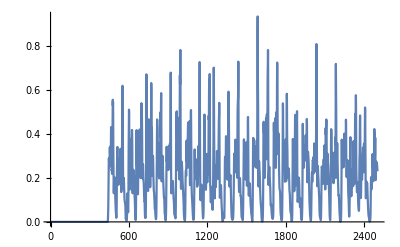

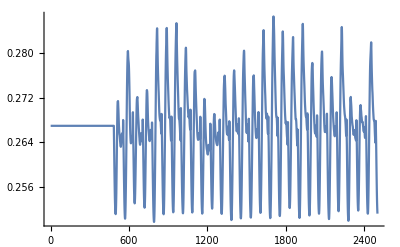

Sub03_(2)run1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411952.0.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411953.0.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411954.0.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411955.0.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411956.0.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411957.0.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411958.0.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.250411959.0.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119510.0.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119511.0.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119512.0.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119513.0.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119514.0.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119515.0.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119516.0.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119517.0.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119518.0.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119519.0.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119520.0.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119521.0.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119522.0.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119523.0.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119524.0.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119525.0.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119526.0.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119527.0.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119528.0.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119529.0.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119530.0.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119531.0.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119532.0.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119533.0.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119534.0.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119535.0.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119536.0.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119537.0.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119538.0.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119539.0.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119540.0.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119541.0.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119542.0.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119543.0.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119544.0.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119545.0.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119546.0.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119547.0.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119548.0.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119549.0.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119550.0.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119551.0.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119552.0.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119553.0.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119554.0.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119555.0.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119556.0.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119557.0.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119558.0.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119559.0.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119560.0.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119561.0.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119562.0.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119563.0.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119564.0.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119565.0.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119566.0.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119567.0.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119568.0.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119569.0.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119570.0.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119571.0.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119572.0.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119573.0.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119574.0.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119575.0.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119576.0.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119577.0.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119578.0.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119579.0.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119580.0.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119581.0.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119582.0.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119583.0.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119584.0.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119585.0.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119586.0.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119587.0.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119588.0.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119589.0.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119590.0.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119591.0.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119592.0.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119593.0.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119594.0.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119595.0.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119596.0.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119597.0.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119598.0.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.2504119599.0.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195100.0.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195101.1.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195102.1.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195103.1.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195104.1.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195105.1.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195106.1.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195107.1.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195108.1.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195109.1.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195110.1.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195111.1.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195112.1.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195113.1.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195114.1.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195115.1.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195116.1.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195117.1.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195118.1.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195119.1.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195120.1.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195121.1.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195122.1.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195123.1.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195124.1.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195125.1.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195126.1.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195127.1.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195128.1.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195129.1.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195130.1.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195131.1.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195132.1.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195133.1.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195134.1.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195135.1.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195136.1.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195137.1.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195138.1.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195139.1.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195140.1.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195141.1.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195142.1.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195143.1.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195144.1.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195145.1.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195146.1.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195147.1.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195148.1.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195149.1.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195150.1.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195151.1.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195152.1.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195153.1.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195154.1.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195155.1.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195156.1.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195157.1.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195158.1.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195159.1.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195160.1.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195161.1.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195162.1.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195163.1.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195164.1.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195165.1.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195166.1.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195167.1.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195168.1.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195169.1.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195170.1.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195171.1.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195172.1.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195173.1.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195174.1.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195175.1.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195176.1.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195177.1.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195178.1.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195179.1.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195180.1.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195181.1.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195182.1.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195183.1.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195184.1.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195185.1.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195186.1.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195187.1.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195188.1.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195189.1.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195190.1.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195191.1.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195192.1.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195193.1.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195194.1.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195195.1.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195196.1.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195197.1.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195198.1.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195199.1.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195200.1.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195201.2.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195202.2.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195203.2.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195204.2.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195205.2.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195206.2.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195207.2.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195208.2.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195209.2.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195210.2.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195211.2.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195212.2.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195213.2.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195214.2.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195215.2.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195216.2.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195217.2.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195218.2.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195219.2.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195220.2.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195221.2.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195222.2.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195223.2.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195224.2.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195225.2.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195226.2.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195227.2.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195228.2.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195229.2.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195230.2.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195231.2.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195232.2.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195233.2.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195234.2.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195235.2.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195236.2.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195237.2.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195238.2.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195239.2.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195240.2.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195241.2.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195242.2.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195243.2.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195244.2.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195245.2.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195246.2.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195247.2.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195248.2.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195249.2.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195250.2.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195251.2.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195252.2.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195253.2.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195254.2.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195255.2.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195256.2.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195257.2.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195258.2.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195259.2.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195260.2.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195261.2.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195262.2.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195263.2.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195264.2.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195265.2.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195266.2.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195267.2.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195268.2.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195269.2.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195270.2.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195271.2.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195272.2.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195273.2.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195274.2.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195275.2.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195276.2.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195277.2.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195278.2.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195279.2.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195280.2.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195281.2.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195282.2.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195283.2.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195284.2.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195285.2.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195286.2.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195287.2.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195288.2.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195289.2.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195290.2.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195291.2.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195292.2.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195293.2.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195294.2.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195295.2.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195296.2.9500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195297.2.9600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195298.2.9700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195299.2.9800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195300.2.9900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195301.3.00.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195302.3.0100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195303.3.0200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195304.3.0300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195305.3.0400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195306.3.0500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195307.3.0600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195308.3.0700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195309.3.0800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195310.3.0900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195311.3.100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195312.3.1100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195313.3.1200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195314.3.1300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195315.3.1400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195316.3.1500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195317.3.1600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195318.3.1700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195319.3.1800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195320.3.1900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195321.3.200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195322.3.2100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195323.3.2200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195324.3.2300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195325.3.2400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195326.3.2500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195327.3.2600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195328.3.2700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195329.3.2800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195330.3.2900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195331.3.300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195332.3.3100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195333.3.3200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195334.3.3300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195335.3.3400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195336.3.3500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195337.3.3600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195338.3.3700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195339.3.3800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195340.3.3900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195341.3.400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195342.3.4100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195343.3.4200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195344.3.4300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195345.3.4400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195346.3.4500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195347.3.4600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195348.3.4700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195349.3.4800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195350.3.4900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195351.3.500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195352.3.5100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195353.3.5200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195354.3.5300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195355.3.5400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195356.3.5500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195357.3.5600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195358.3.5700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195359.3.5800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195360.3.5900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195361.3.600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195362.3.6100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195363.3.6200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195364.3.6300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195365.3.6400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195366.3.6500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195367.3.6600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195368.3.6700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195369.3.6800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195370.3.6900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195371.3.700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195372.3.7100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195373.3.7200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195374.3.7300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195375.3.7400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195376.3.7500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195377.3.7600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195378.3.7700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195379.3.7800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195380.3.7900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195381.3.800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195382.3.8100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195383.3.8200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195384.3.8300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195385.3.8400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195386.3.8500.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195387.3.8600.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195388.3.8700.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195389.3.8800.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195390.3.8900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195391.3.900.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195392.3.9100.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195393.3.9200.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195394.3.9300.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195395.3.9400.266994900.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195396.3.9500.26699490.0025544515222357580.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195397.3.9600.26699490.0052773823914861760.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195398.3.9700.26699490.0077034987658408220.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195399.3.9800.26699490.0103994670372640540.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195400.3.9900.26699490.013844282517428810.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195401.4.00.26699490.017984974012195720.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195402.4.0100.26699490.0210918698762856820.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195403.4.0200.26699490.0205259289971832450.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195404.4.0300.26699490.01826948454013480.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195405.4.0400.26699490.019007627768508320.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195406.4.0500.26699490.0244836743580104030.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195407.4.0600.26699490.038426155643148510.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195408.4.0700.26699490.067535560343298930.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195409.4.0800.26699490.11069454734248620.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195410.4.0900.26699490.146398158490036180.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195411.4.100.26699490.181954740038870550.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195412.4.1100.26699490.25223988791611440.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195413.4.1200.26699490.313742910636552350.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195414.4.1300.26699490.323309633850071050.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195415.4.1400.26699490.30353671893099250.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195416.4.1500.26699490.296524892494174960.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195417.4.1600.26699490.28659489728754060.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195418.4.1700.26699490.232584671829928920.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195419.4.1800.26699490.1649263706578650.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195420.4.1900.26699490.151311761904798170.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195421.4.200.26699490.181182221823003250.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195422.4.2100.26699490.21962279786297370.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195423.4.2200.26699490.259218728969145440.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195424.4.2300.26699490.28483506985310750.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195425.4.2400.26699490.26451043201446850.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195426.4.2500.26699490.202076387635732770.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195427.4.2600.26699490.17223394178583510.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195428.4.2700.26699490.196165672876227770.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195429.4.2800.26699490.21695147690056430.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195430.4.2900.26699490.21311569711571630.3763106300.3902017800.2779214900.3171631100.523503100.2910414100.3887779800.4112400400.25041195431.4.300.26699490.18630466007387380.3763106300.3902017800.2779214900.3171631100.52350310.00410764950660162750.2910414100.3887779800.4112400400.25041195432.4.3100.26699490.158109933684401630.3763106300.3902017800.2779214900.3171631100.52350310.0056521666031187310.2910414100.3887779800.4112400400.25041195433.4.3200.26699490.140931101962473770.3763106300.3902017800.2779214900.3171631100.52350310.00769552635503315250.2910414100.3887779800.4112400400.25041195434.4.3300.26699490.111711497101627630.3763106300.3902017800.2779214900.3171631100.52350310.0098478715861767420.2910414100.3887779800.4112400400.25041195435.4.3400.26699490.092323131285249670.3763106300.3902017800.2779214900.3171631100.52350310.0115314187598326810.2910414100.3887779800.4112400400.25041195436.4.3500.26699490.108419855071053730.3763106300.3902017800.2779214900.3171631100.52350310.0129110350384494240.2910414100.3887779800.411240040.0053561953823612310.25041195437.4.3600.26699490.10148329252242480.3763106300.3902017800.2779214900.3171631100.52350310.0140671730734952490.2910414100.3887779800.411240040.0057584053212093990.25041195438.4.3700.26699490.0612155829604974640.3763106300.3902017800.2779214900.3171631100.52350310.014643213552887860.2910414100.3887779800.411240040.0060413044795645880.25041195439.4.380.0129610908868462440.26699490.024145190787550950.3763106300.3902017800.2779214900.3171631100.52350310.0140649510765300960.2910414100.3887779800.411240040.0072004392651167130.25041195440.4.390.0306839094949781060.26699490.0091368497447876710.3763106300.3902017800.2779214900.3171631100.52350310.0136216985176059130.2910414100.3887779800.411240040.010256868213860530.25041195441.4.40.0552420285883525460.26699490.0063269256986836350.3763106300.3902017800.2779214900.3171631100.52350310.012227591724907780.2910414100.3887779800.411240040.0117027546531545560.25041195442.4.410.090594312499822710.26699490.0073941164473559630.3763106300.390201780.0088394896066044830.2779214900.3171631100.52350310.0096834279616790590.2910414100.3887779800.411240040.0091707987680508250.25041195443.4.420.14140660142389280.26699490.0080502665226405370.3763106300.390201780.0132670726280662830.2779214900.3171631100.52350310.0069726119714975220.2910414100.3887779800.411240040.0079132740121284350.25041195444.4.430.198308145558449780.26699490.0084922436951273530.3763106300.390201780.018652167186550240.2779214900.3171631100.52350310.0052871344112596970.2910414100.3887779800.411240040.008400783342279840.25041195445.4.440.253802528627771140.26699490.0093092682675368820.3763106300.390201780.0234606148875074680.2779214900.3171631100.52350310.0056719508870659860.2910414100.3887779800.411240040.0082214070773864910.25041195446.4.450.289146030543287750.26699490.009365712369189260.3763106300.390201780.0256560000093288030.2779214900.3171631100.52350310.007012360151706840.2910414100.3887779800.411240040.00715300859152540650.25041195447.4.460.284037786970777860.26699490.0098343427814481120.3763106300.390201780.0261579854525444930.2779214900.3171631100.52350310.0090122338684769320.2910414100.3887779800.411240040.0068674047660047080.25041195448.4.470.258540296656165350.26699490.0091775104220133440.3763106300.390201780.0255956375044462220.2779214900.3171631100.52350310.0118067574421745690.2910414100.3887779800.411240040.0078902325060626450.25041195449.4.480.248715629990211680.26699490.0081619255339232760.3763106300.390201780.022970798087965540.277921490.00239101773005334030.3171631100.52350310.0147863350322737180.2910414100.3887779800.411240040.0090031251522831540.25041195450.4.490.258073847632059260.26699490.0065065280801383980.3763106300.390201780.019330217544897310.277921490.00327203634506300670.3171631100.52350310.0167572384031607070.2910414100.3887779800.411240040.0106202061162081390.25041195451.4.50.28270362449964890.26699490.0055696025214342930.3763106300.390201780.0165906788530289260.277921490.0042931579629878870.3171631100.52350310.0178350813758318820.2910414100.3887779800.411240040.0157184135071269030.25041195452.4.510.30682059100022990.26699490.0076379834596432840.376310630.0066893705197765910.390201780.015742778500651070.277921490.0049209053727539750.3171631100.52350310.0176361802565333970.2910414100.3887779800.411240040.0223441783128409640.25041195453.4.520.3371289294056580.26699490.0108599268885516790.376310630.0067940792211756880.390201780.017163807644605620.277921490.0043296358507264470.3171631100.52350310.0148257006558076880.2910414100.3887779800.411240040.026327548306036330.25041195454.4.530.339637249020781240.26699490.0108366439703211290.376310630.0053725379115091260.390201780.0187022819382800760.277921490.00326988928605404260.3171631100.52350310.0115920400038545860.2910414100.3887779800.411240040.0290111944230595840.25041195455.4.540.3095704150132330.26699490.0113941743454837250.376310630.00585682511765554460.390201780.018152050333210160.277921490.0030647489078296440.3171631100.52350310.0100943656111550690.2910414100.388777980.00104814799342328870.411240040.0301773163687041050.25041195456.4.550.309157602112976160.26699490.011507850406548140.376310630.00775122409756052750.390201780.0159793868590952830.277921490.00345674555020565950.3171631100.52350310.008963307573005250.291041410.0026751213826030580.388777980.00205841592266024260.411240040.0286244115335060130.25041195457.4.560.32290311414443670.26699490.0097493949795155730.376310630.0088571323500179850.390201780.0144146934881647720.277921490.0033099209732137980.3171631100.52350310.0066457870560075860.291041410.003640538075077920.388777980.0024605116008605650.411240040.026541973533994790.25041195458.4.570.343722113156609830.26699490.0082876437840972830.376310630.0099082729856240570.390201780.01669939215399840.277921490.0028645578735754020.3171631100.52350310.005004104651595140.291041410.0049142842996631430.388777980.00260986519453893430.411240040.0259533755965981540.25041195459.4.580.337214006983619640.26699490.0076863244004229750.376310630.0144588683922230230.390201780.0266837436948870780.277921490.0027824411357989040.3171631100.52350310.0046421836407220080.291041410.0073470127580645220.388777980.00330409173557502740.411240040.0262730132301429860.25041195460.4.590.28941024184218810.26699490.0082921906319320480.376310630.0266616765444829850.390201780.046283323234811830.277921490.00329334234772685850.3171631100.52350310.0043248038523846720.291041410.0098567039337089080.388777980.0039590837611275830.411240040.0261576311819447270.25041195461.4.60.300476445927695570.26699490.0111311341293295580.376310630.048068803850277590.390201780.073658342185702190.277921490.00387730450782459120.3171631100.52350310.0039883928859639430.291041410.0120549357898329270.388777980.0043478972292079010.411240040.0253685222440620320.25041195462.4.610.385092051900442930.26699490.0142987551305061020.376310630.06922499312274090.390201780.103651159059545110.277921490.00357169592487168030.3171631100.52350310.0036686972133472310.291041410.019780829909072290.388777980.0052513849919099340.411240040.028750842162360680.25041195463.4.620.43174620990561370.26699490.0147247075557074160.376310630.069127156494624110.390201780.128692378654449690.277921490.00305351696358626640.3171631100.52350310.0035239129345631010.291041410.043859192451067130.391947380.0078605470836771250.411240040.040262064266149880.25041195464.4.630.379871378355213840.26699490.0121206454145468250.376310630.052572248359525880.390201780.141672599195862170.277921490.002662038725638870.3171631100.52350310.00388672894274117280.291041410.088731189992127660.395095160.0131272902099681230.411240040.055009977557218610.25041195465.4.640.32262564313319050.26699490.011727532147232490.376310630.045731480811980240.390201780.139550719907194250.277921490.0023570591046114910.317163110.00183619509100263960.52350310.0037867107751428130.291041410.145390366086499740.398231210.0214688634875180270.415189570.069728487409644120.25041195466.4.650.302563927806399350.26699490.0144549568804009740.376310630.064394284084797980.390201780.124947561698380380.277921490.00280879158668342770.317163110.00324810375986834450.520437720.0038998724982746390.291041410.20740371128369660.401365360.033835547311701830.419262750.084248936173932670.25041195467.4.660.263523669965427750.26699490.0144644108010897310.376310630.103799573474362970.390201780.106208277808956860.277921490.0043073538700492260.317163110.0049258690082259540.517222230.0054964294286572620.291041410.27384253014774840.40446270.051609761850137080.423423840.099094105178983730.25041195468.4.670.233328141199318860.26699490.0113871973503138020.376310630.133411432335451440.390201780.090124286764260790.277921490.006364864243680360.317163110.0066589987731064590.513859190.0069106104100524690.291041410.32209988531400660.407502360.072160168100645990.427635640.11459076652306640.25041195469.4.680.240305174031574250.26699490.0091985571838458980.376310630.118705810340882980.390201780.073595787989910830.277921490.0093623874071763060.317163110.0090327577869421150.510371940.0081711604813026160.291041410.328370373199946440.410452620.087956249399832130.431851660.130120502198321520.25041195470.4.690.21899966589784180.26699490.0119977287551950460.376310630.072660389407286310.390201780.053642350469226060.277921490.0143241553498247780.317163110.012866005410406080.506845030.0094027120513749920.291041410.31905991130634980.413297290.09637945230208130.436029350.14444230156933080.25041195471.4.70.220773722606216140.26699490.0180479006361867030.376310630.035517811980388820.390201780.0372930004010589840.277921490.0222950681924478570.317163110.0173967099582834280.503363980.0109499975246557420.291041410.32503684237550360.416052910.100101161416616820.440122480.15686676858323580.25041195472.4.710.30269270887773340.26699490.0247133870510040.376310630.0184066097168076630.390201780.030071508342008350.277921490.033962665378750210.317163110.0210199405719876980.500039360.0149733897654624210.291041410.32765837094756420.418536450.100592434682056160.443890950.167490405574324040.25041195473.4.720.35338403170506250.26699490.0281988539425399550.376310630.0143150139240833930.390201780.026798472316966130.277921490.049102577042594850.317163110.023022858402738080.496860480.0212581745865266960.291041410.30714835508579090.420781550.097088966347400410.447321050.178489386199130570.25041195474.4.730.40057674229137230.26699490.0281523817098734840.378349090.015514008148949330.392165860.023205350660057280.277921490.067421093838870540.317163110.0236655803010660320.494025650.0274098031222204560.291041410.27061598132467610.422644420.093603104838288780.450216710.195048649066002860.25041195475.4.740.49756540320607060.26699490.027627222652416380.380195560.018457534568771870.393908130.0202270434995728760.277921490.088771027908504550.317163110.0232079534431946370.491620440.033196618055812330.291041410.22975284111300790.42414620.092233766736965140.452568860.224871151972709520.25041195476.4.750.55581698651053850.26699490.026507868506346070.381680670.017988491245936410.3948860.0177829292777672530.277921490.111033329134507590.317163110.0214049647090796820.489695860.0441795438589350150.291041410.193896928275182650.425331560.084371312047008540.454400810.27299838741548990.25041195477.4.760.5295631974177060.26699490.0265161051622827170.382798990.0125854613308040450.395549580.015816982623376990.277921490.129715370944890750.317163110.0199846545347534820.488333750.0626346095483290.291041410.15856040948848990.426199410.07100017393286480.455689680.33618952156141240.25041195478.4.770.5468614417876240.26699490.03067684259209170.383622720.0080120380548210040.396092120.0155414415012398760.277921490.141756170427096760.317163110.0213384378068444330.487567680.080259166648649680.291041410.115607376573433850.426729440.0583132276838685540.456427290.40231153379461860.25041195479.4.780.49249583548919130.26699490.036594909312777310.384110730.0087786189937725820.396485670.0170865086149530640.277921490.15052538267020270.317163110.0260643300349610240.487451820.089809054599013740.291041410.090465406639662070.42685360.044987743386736960.456563040.45534001292496480.25041195480.4.790.35142720961360480.26699490.0509373885101058260.384328650.0120812846987956540.396731220.0228448466828704770.277921490.16283375490908380.317163110.033129162715439640.48788030.096397644129837420.291041410.100681253709223320.426518630.0328205796155678350.456115070.4852108922423930.25041195481.4.80.270653612066632350.26699490.083689675192488950.383885840.0141012627585489870.396411010.038059562990376620.277921490.180545148178456270.317163110.043268796489838670.488724150.111621739304617370.291041410.128905119136709820.425809270.0275488514441901180.455194420.49646857458268250.25041195482.4.810.214148754024595070.26699490.127505286798294260.380002320.0207202373124270550.392878850.065483296197992620.277921490.206417373224481450.317163110.0563592505405542540.490062120.129015078805648410.291041410.158825291861434510.424818820.026881192334944560.45381150.50421658956659190.25041195483.4.820.144242144100796550.26699490.175193091360957620.377905290.029450223145398850.391647820.095859447836749680.277921490.239203987704875720.317163110.067798399966757880.493013880.149278689550609360.291041410.179246334327536060.423006750.0263872340591470.45098840.52216606681879010.25041195484.4.830.13072784628045740.26699490.21007912660963160.378012790.0350838236513397250.39185480.118973053423691090.277921490.268428761817305240.317163110.081754776612355560.496799470.193489028202184580.291041410.184241465675521720.420693920.0246412739846264970.44720420.54672346626484060.25041195485.4.840.15485428466385910.265214460.242472480341575760.378043560.043303226780496230.39190860.14003089579888610.279706340.28777769231591710.317163110.103469265351631960.500358960.236365870421390150.291041410.174557944847463930.418154330.021560585081619510.443270980.55578003615992180.25041195486.4.850.182402816722073650.263569850.27342659979740680.378270130.066233202126099330.392115970.160493739708947950.281312140.28639449318110520.317163110.120133141689004740.503502120.24160723828476610.291041410.154385605168452070.415582430.017923685269557420.43952850.53059989381712410.25041195487.4.860.19955184536706850.261776830.267484466046553570.37886530.117209919935152440.392670680.212386281648860230.283016350.2644321425870160.317163110.121714728392258250.506344690.238203447915537630.291041410.13148830303327440.41304480.0143210323225801130.436008170.47102207360914380.25041195488.4.870.20439515782178450.260036510.25311924447990930.37960470.191997854053698960.393364160.345539729357570660.284624640.23990451699539050.317163110.107039588886349430.5087570.238510317350484030.291041410.118248943215662760.410773160.0116135411547262580.432958970.388569620811401560.25041195489.4.880.203379753380603520.25840150.25825156199206710.380410080.242151195503877310.394125640.49034869241127560.286094930.213379408996088570.317163110.081498352280331770.510801430.22031354036878520.291041410.12807483486302280.408724440.0104768460654456970.430323290.29915415991313390.25041195490.4.890.196947529733049440.256854190.30593498125983460.381301060.299197537365436970.394979360.52013954951115230.287450530.185371659245575250.317163110.0586922393393439350.512529920.192291300495966880.291041410.168973979123130170.406847250.0115767584060080830.428041970.21776843166126610.25041195491.4.90.182347514032165060.255425940.38610656677333740.38226530.415531989405876930.395916990.43851124986281150.288671250.15992616276237110.317163110.042346269480326350.513972170.172666309680604290.291041410.244245176777581170.405134130.015818184189620310.42609050.159340900496776270.25041195492.4.910.165150140329457570.254165910.42225116527028910.383249620.49918601064778770.396886650.37419504593667140.289724160.133683316034821030.317163110.0297484911419140350.51522490.150925607653731750.291041410.344082908610361060.403491530.0238573339638747450.424346270.140794214326489030.25041195493.4.920.149730397218432370.253186530.37365200835416670.384130320.49143092852153820.397763750.346362493673955050.290527160.105890000515507320.317163110.0205779286576661150.516279580.117757353818339920.291041410.428757363685982440.401968590.034676421637339670.422830810.162718546860415430.25041195494.4.930.133479635749808620.252460410.27530209586519660.384922980.402867119689190030.39856210.31887960631470690.291113920.087392435445392710.317163110.0149952415122432980.517155880.083214679363272970.291041410.48899368374339470.400566220.045606603269052980.421521590.202281538059486840.25041195495.4.940.114924617048902560.251905150.172860553957907750.385711150.305201135134901440.399364130.270251140905801430.29155770.078796286412709230.317163110.0121315445754115910.517898840.055179768075564780.291041410.54181679564455980.3992270.05414388802920350.420356340.239809770012198250.25041195496.4.950.096451381976766030.251500630.09327693294607790.386517610.34688471496047740.400191110.220980193029657050.291878350.067371173863700160.317163110.0117914936102129030.518539210.035348467269683060.291041410.59029621529897770.397906730.059354150733460180.419295650.26330420264958960.25041195497.4.960.07964020239157230.251240740.0594734680851605750.387336780.44559456836952610.401034670.195075447947151840.292083180.0496448578394570460.317163110.0128037471137795420.519078920.0238365356794706630.291041410.59477103674466280.396604450.065482351213450560.418342050.26389849539346320.25041195498.4.970.064022154166206090.251128710.054835389395639760.388143310.47228391861587450.401865870.18786575997909120.292171190.031828827005035770.317163110.0133763484634804150.51946040.018231311127288310.291041410.53579639970809690.395396210.075610601353211490.417572760.238609365864750760.2484469499.4.980.0510230563964342650.251310320.05554382632067980.388761030.442827510943613940.402504380.179679666296628850.292028430.0190489539973221840.316003770.013449212228391970.519679580.0154945660475560540.289943620.469240963376446050.394320880.088762479097362850.416996220.19475132779842410.24645152500.4.990.043085285218003160.251795310.058171419500046360.389134360.38674089697315690.402891880.163924993214770470.291644990.0122374731800330010.314775990.0132674692424014920.519764140.0140113747158933120.288784310.43872610960136080.393364370.101474954102000030.416572660.145455293322715060.24445694501.5.0.034128754447407890.252598560.070098995953783190.38921220.30514676628678970.402976310.144328355836219640.291002850.0090429188659561110.313523930.012782794782947050.519716470.0130096607821910680.287604940.40268386830248350.392538590.106377280643414450.416294070.10081292283715910.24251108502.5.010.023440062177664890.25370190.08837361826250780.388977610.227111169117976240.402741320.12239719681905820.290106280.0073175024471784830.31228550.0123161751933576930.519577160.0129642433209848540.286440810.314877863595127870.39179410.099110011814859860.416101830.06566558851553640.24056044503.5.020.0185791404295253950.254849550.09621554859035490.38862490.165756767549481880.402382380.096804347322458420.289155680.0064197146587177740.311117430.0122836289288362780.519291730.0134337873890266520.285344940.21479647241999540.391282270.083217715322039740.416112880.040822834230304980.23882635504.5.030.023589170290826220.256628930.095122178215565940.387649310.112178274974618240.401397920.068626168663836630.287644990.0059737201505359660.309946040.0123447692435787860.519122760.0145822167857153350.28424810.13835023477665060.390521610.065939441943086070.415889240.024813653717656110.23675193505.5.040.0420068479001535350.2584260.0987795012282150.386583320.068879938113873190.400320310.045938329777964020.286073190.006197817806478070.308811520.0121948799505836540.518902320.0176620877307201750.283187870.090626247967411690.3898640.051974392709702550.41573560.0155638474039203330.23481748506.5.050.085903402040079510.260265590.089914975958122830.385358160.0401894662658997540.399084230.030780063784627810.28441550.006858035165813490.307796270.0125487470289412630.518744990.0212864102491610720.282240840.062724567238444580.389221770.041739526358701770.415533670.0108045148710413410.23300826507.5.060.159950725213301250.26216320.062035642136499520.383949490.025033037803255270.397668440.0230825841905471230.282653190.0071584915310927990.306918440.0143627033191039020.518717010.0247836021884891080.281423340.045222342528939020.388514960.035458721351297080.415201780.0084717256964933050.23125501508.5.070.231867450339845880.264040810.0357765191936816050.382418560.017013142353396160.396136940.0188024048439343720.280856480.0068545974438982610.306212620.0169881886351140670.518841550.027739096368980790.280766910.03387919707417620.387739860.033533042172379810.414725140.00651216400251382250.22960095509.5.080.27438567608955670.265909190.020193304664445750.380740770.0119609432508430580.394468680.0154723743307735580.279015660.0066540936469326580.30571220.0188781771103034570.519161620.0290027489798815940.280301950.0259891998308252220.386852190.034446184819919050.414053110.0050660197472882970.2280364510.5.090.32550791740186220.267729580.0148599880702830760.37892280.0086667313014121210.392674580.0152530869593942470.277170790.0061795581769471140.305488930.0190852008947512250.519708690.0273570995439321070.28009460.020154402554842160.385855180.034027478414966840.413166940.0051702953604678980.22664525511.5.10.341158262471529030.269293720.012459745403645560.377133260.0070694539700502970.390924570.0156655459847683950.275544770.0053924333249161710.305663420.017497701466880380.520588880.023240810283450630.280256640.0154742696128209940.384690750.0299514215991429360.411973620.0052623790346394430.22544851512.5.110.295792769187091740.270538310.00686709861584457360.375434220.0076670971076370720.389277920.0140841738112283380.274223770.0048301592797231190.306275010.0150045497777800160.521800860.018382225605044370.28082490.0116343103958262730.383387580.0234513429214027670.410499060.0044286063514643350.22442551513.5.120.267399287210377260.271189040.0037909100151395740.374125480.0076989363439250630.388022370.013046175585146930.273523460.0043943796576172420.307350330.0133954038544862040.523355520.0139035969370701740.281825390.0077392537597495660.382008390.0170865243145337240.408765770.0048268717949487320.22378174514.5.130.27095225245036870.271379860.004937272866630440.373074660.0067684792526051960.387018370.0118631602198072430.273316840.0039303761774362710.308858060.0140040466135535110.525279960.011127421471546290.283231320.0055158313029972330.380464420.0123405770751203930.406688360.006420948327515230.22339629515.5.140.25306110691902560.271396160.0063682815626867440.371966730.0058537470219976410.385947030.0087193907885051380.273299160.00352274465887694950.310759060.0171584145785478940.527473590.0104818084465481340.285009140.0042187209398420430.378843770.0094129522095424380.404354240.0085380704080334890.22332943516.5.150.234987887069035150.271447970.00604283268134014550.370608860.0042538212986264190.384609280.006002012664602570.273242950.0046299815919076510.312930530.0218364103494260750.529816070.012855101194387260.287046860.00523702475806834150.377176350.0078703445387880360.40183960.012393672724233810.2234036517.5.160.22099597107663420.271014530.00389085921778426070.3695830.00272343793267497850.38356540.0053800094792427980.273711910.0071887470617583080.315313770.0272851537869424240.532228880.0174079252604896240.289291720.009116712043258560.37553080.007086920132353220.399213610.018379117407965850.22366217518.5.170.184467890765048270.270392270.00127665029734285940.36863520.0024593548821379970.382563790.0044464143703386670.274380030.0089125298436496850.317758520.032643909591835510.534677870.020112396247221590.291606550.0122959078077408050.373853240.0067191310894686640.396484710.0254035256851143050.2239091519.5.180.16864182933897870.269864450.00047856150742217840.367483250.00264889091074068130.381327540.00298463002311687150.2749420.0086245313743955680.320238160.037441090488652370.537093440.0188093419349330760.293972020.0125843869125263230.372243920.0065721210719277840.393764880.0333170813312558340.22432403520.5.190.188989114377633580.26916420.0029771361105307120.36644270.0042346364586325060.38016570.00377358767084417240.275680860.0070983441407149840.322738680.0426371249165580850.539505970.016130534096919130.296378980.0110454871364897170.370652040.0064806893594669980.391039720.042912144396080770.22473507521.5.20.223589756398192730.268317050.00576251056430288850.365548570.0061945647368604010.379118010.0073597795102477560.276564530.0047604342007419410.325133640.048528022724224540.541690120.0150337446084063180.298704320.0092022593963786770.369267090.0062974845944057980.388559510.05447436034757930.22517581522.5.210.259238061949298550.267622790.0055448676224440150.364521760.0074619960794305140.377917220.0107047108099687980.277280430.0027178914799242510.32732810.0568000330010749450.543548490.0158247744016758140.30085210.0094190955698539030.36811450.0058033294029991630.386359320.067545364679076750.22581863523.5.220.27509079587054780.267009560.00446247754294455850.363447020.0065183512039048710.376648320.0113666737359893670.277906580.00187478603923020720.329319440.069644359246973130.545964270.017606191039200080.302817380.0096362140984360980.365885890.0047688899044275650.383142190.081794709162487950.22535997524.5.230.25322808810008990.266603750.00289909416222938670.36215190.0042189363605136320.375137090.0096342234189816230.278317770.002167598511938630.331166650.081242903751729750.546879350.0202672894014670480.304657640.0085847676944889650.365814990.00358546302318059040.382025330.09518295710240230.22741757525.5.240.211524667235665680.266158760.00137191693530343030.360979210.0019655086215611630.373731220.0067272949422975270.278765740.0022371383326185560.33280390.082502147698319940.547454830.0211385344949662660.306305830.0074009151649811330.366107440.00281805442561190460.381316760.10184114681985620.22979848526.5.250.204794662115556280.265774150.00296485047938307080.359912620.00192292475878126080.372432240.0040269132046539870.279150490.00149817546062798930.334179290.073464639519344510.547581550.01842780810219410.307705090.00706771483437048950.366882240.00219366280949592940.381189020.095300689482884170.2324954527.5.260.240743985986812990.265447240.0071705439065513710.359019190.0043803315668840990.37132430.00405525354849185350.279475740.00125941788789022350.33527430.05792895163634940.547243910.014619486679681290.308830060.0076477900021794830.368139730.00183869223506640430.381693710.079597524594930950.23533372528.5.270.28096488792557130.265342810.0102254072594270880.358162580.008479666707400790.370289480.0068796652475265980.27957930.00174185181717880270.336093080.04062206351889780.545146280.0113149137581484980.309678430.0087099443367743870.371758160.00208221169351579820.384771460.062183798907179890.23983497529.5.280.2913298045682760.265118950.0108545088555917110.357670930.0144129213170275350.369652840.0117400427252292320.279800720.00312451484748017640.336686290.025351637349842210.544006650.0092783138539381040.310297420.0102255611989084780.373769230.0021767826867211130.386390010.0479588102358955850.24249485530.5.290.269032439740535530.264834190.0112398122552207250.357497010.0204100124227738730.369378190.017798106069037610.280081290.0036722212927055590.337060670.014733904385574820.542511670.0084944090851813560.310690160.0119962653385454080.376095440.00206211814596143340.388502020.0409363955996211240.24505246531.5.30.260888147568026360.264515530.012231035605086990.35761110.0286938532225172320.369441420.0249269294563306680.280393790.0027980028131110850.337230440.0086652191121264640.540703690.00764200902758705150.310868660.0140691067402947870.378700650.00248565923289362350.391064160.0395968464456137660.247492532.5.310.289733954595857430.264193210.0125889039380664480.357993080.0445954697882247550.369827990.029534423803404420.280708310.00246708998996267260.337192440.0056604162205612830.538630510.0062533404712515250.310828770.0188703181095934080.381513910.0033347669047977090.394005870.037558398821897770.24976894533.5.320.331605532715898650.263963650.0123012976028151040.358555410.048052631475163390.37045380.0270039473761235940.280931360.0027507336592652880.336936290.00438121483946190150.536476410.0053396872512826190.310559490.032477002600921680.384272530.0043252723609108920.397049320.034345386695159930.25174449534.5.330.328850949540052730.263676210.0121982868361462940.359427150.0312517504516590660.371435960.023751542516392650.281209520.00342180893979572360.336473320.0043917499828422320.533906030.0057042773394741790.310074750.0542516755492657850.387486180.0058168333005241630.400706980.033832539466846970.25375335535.5.340.286776473746850560.263492160.0115549580727814130.36046020.0244829647291995580.372626250.0244496293126828840.281386980.00397143756830865750.335773120.0048928236248591060.531349580.0068612173516385180.309346130.078010824903910730.390526160.0089782182073653120.404319070.0347229790852035950.25544437536.5.350.27522938788297490.263323420.0113351350114535240.361726120.0294019342375790650.374082810.02718301008655850.281549220.00377287092183484650.334829590.00616339409724690150.528712890.0082513515770409280.308371930.092534068703633980.393537960.0141783262345983390.408027660.035349405163641390.25690369537.5.360.31282334074966380.263224610.0124086033307148240.363169350.0296399546856717030.375742060.0248702022576254530.281644020.00303912703020580.333614250.0080514209783244720.525972940.0101667373939200220.307128480.108672468761198180.396538480.022889302591148780.411854210.037355052826310340.25812986538.5.370.31252570835400850.263270120.0121312297526386910.364710470.0372825132457559950.377515590.0222375059364425430.281600380.00265657408878386920.332089650.009772025103661340.523098810.0112630562663029850.305584640.156197884012041960.399543620.03721664867942550.415818490.0448972138223748960.25912616539.5.380.224287780204022320.263448910.0094164572663706210.36633890.053107578685560050.379380410.0304388539347046730.28142860.0030850323859550480.330222550.0105408446217431020.520074680.0117386338340095470.303714780.233046256368655170.402538120.057589419406560590.419901610.059473603565164210.25989068540.5.390.14592526147256230.263670750.0062231254363882670.368109770.067806347555751730.381377540.050291497845935170.281214790.00382807759086799950.32798930.010191935769027980.516907260.0130158659121080920.301502750.300123334832989860.405487910.077512099892779180.424051960.078748096835214140.26043067541.5.40.13563201313872810.263978850.0060130573469602710.369940570.082646443850697720.383413910.081031715900619010.280916620.0048530279994547650.325374160.0100856277308501650.513618540.0142010288793119120.298938920.31300572555307820.408338950.087145954999968840.428198270.098551308592868440.26073756542.5.410.175771240122344630.264409290.0077867864704777460.371726170.109126087254230560.385372930.108752839005450750.280497630.0061693865417013770.322431010.010464149951390840.510170730.0140512020393726320.296081660.267296643946284330.411175850.086640879969815650.432396690.113937084988973970.26092631543.5.420.27312250691794940.26487550.0104585403499340960.373475630.102731987290579670.387252130.108628097870559660.280040660.008963974895023120.319316320.0115459678429701480.506750470.0133573131978563810.293090210.225109972599515070.413875650.082749837775264080.436479540.123127954256441930.26096826544.5.430.33587355859651940.265231910.0126967899395385530.375255860.057464415932994640.389109440.078076393899011650.279689080.0128269965258543340.316178910.0137478452078140960.503465660.0141636356826848710.290109260.232702208838646290.416392470.079858726190454620.440347680.127468870242540750.26089502545.5.440.314834103433280670.265464710.0134648954647260120.377018680.0223090547149248160.39089470.044906129252231010.27945840.0179260302816530330.313051010.0160814533232216220.500318980.0191080483272051580.287160130.25622551399611610.418681610.086241231196198590.443905250.12750016558238940.26073463546.5.450.29979886546056760.265619880.012816382802346950.378658380.0122292607088462720.392506740.026276743210903310.279304180.024476062631902340.310020850.01751205638153540.49738390.0276709441630010360.284318080.25192869270558620.420673940.093904484468609190.447029660.123226455505630630.26051268547.5.460.350493198875312830.265585930.0124459581737478390.380227170.0114377233688079430.394007080.0187622591636601550.279337960.0334295169889928450.307289090.0177690859738072820.494773260.033572351161768420.281768370.218777581273336550.422379030.091432586269589130.449685280.117767840849031750.26029516548.5.470.44570906672286110.265496440.016163831399875460.381560040.0122191236541785010.395250030.0185209928946634580.27942690.045669090996449090.304987080.0174857688459380020.492675790.0347682598786917960.279628690.17892181269006590.423645050.089304654466131660.451695730.118201505782468030.26003595549.5.480.5310713193736070.265427730.02772843567446540.382552660.014014071312679020.39583090.023514513221264370.27949510.060353574913659180.303225610.0180940543559426730.491088010.035796783362782080.277994090.14239333058793220.424580450.095556945161881250.453168170.129889477836119180.259825550.5.490.61542209970315560.265382960.05176899184727130.383198580.0273841444045426280.396127150.03630763047928320.279539510.075770425038019620.3020570.0199206782456682780.490107630.040671434834825590.276908870.108404118469426340.425115910.099985301422156420.454030150.15271833940811240.25965937551.5.50.61965725575170660.265273420.081761040909336420.383614670.0276250441006984270.39636150.0362081433756110750.279648010.08963318949036410.301462250.0222537298035640660.489749080.0537256301072806250.276355870.087314246566540550.425223090.096134129073175460.454275680.187227747379373920.2595075552.5.510.53112463789657960.265092070.12503470397242120.383864720.0391650649550271260.396572070.042048465255970850.279827260.101716768438660120.301342020.0278306611100120860.489966530.064598171306172260.2762440.085679351024517320.424895140.091435854949424290.453935780.229636174020078220.25930046553.5.520.413263451811723640.26505920.178901530321609830.383797730.047373729303651420.396565540.068234769275853970.27985970.116836392131295920.301542590.037449870469136350.490625370.068230681756291530.276430610.102407763225071380.424216210.088459646795196050.453133280.27843791791358270.25904874554.5.530.269088715448805250.265890550.226391100638928120.382643580.050005934881916830.39559310.109438147276255140.279034290.140210421625522890.30210050.049357007983152610.491665020.080230826472827850.27694930.13095884786797330.423325790.078992927218674960.451976270.337095696048279660.25898537555.5.540.1708745583707410.268037240.255319522242226150.379616190.0618717426179025140.393033810.151716868138549570.276853950.17004956414180170.303539280.066016007659329450.493565050.103677936773805980.27828520.162437668978600870.421929390.063837233081163830.450026780.406305323255724050.25906404556.5.550.148843442315566620.267225630.288568878679228370.378726980.081203772805625380.392521420.177126034351957030.277686620.20583860073445720.306856120.092609212200981050.496927960.151145696051213360.281365340.186972184055059250.419840440.052070701896664140.446757890.475017870101741070.25971529557.5.560.167735892903038420.265099580.313288055654849460.378908380.102818024584258260.392756570.185315651093531760.279819850.242577241695444420.310529810.126211365442563640.500568030.220727771451511620.284794450.195847689510279530.417555590.045584633992160350.443050710.52803147309427810.26061081558.5.570.18872608095236560.263766980.29790586786457710.378606930.12329550723278920.392456920.1966881468945540.281121810.26477491817853090.313330740.149200000063236330.503713370.257096823715051270.287423190.18645023687774640.415269020.039448890849417770.439545090.56087938479036150.26112892559.5.580.199279626784823830.262120820.289258556908373040.378911180.156038294900064880.392728160.196549386281564430.282693130.276775450231313950.315477750.1468211784608190.506482510.259095309223407070.289446560.166414265450745950.41299930.037153112246140670.43625870.58236255873540620.26123162560.5.590.200481935899674170.260355470.32363442848156770.379531650.21328094479144780.393301870.205772978076679440.284333230.30411029401793760.317183770.130699987063297330.508985020.28277595942912530.2910610.149203814756681370.410768630.0422427448556393360.433192070.60073748176880770.26091003561.5.60.189719228521704530.258667160.356101616455047560.380268510.288796955279451260.393990930.26432284267024590.285858690.343448762324775560.318508580.115975906737273230.511153630.33340206651671690.292319960.14149923980965280.408707510.047328223686867790.430475690.60930273589994230.26032113562.5.610.170134150505118930.257103570.362081185561591360.381059110.369894296050146950.394738850.325141516470987050.287234380.365421467909700040.319516180.107252434807431870.513069460.37812864355166850.293281130.142162573393292860.406717630.045234357131458540.427985710.59221569363744580.25950179563.5.620.149714544955562220.255685150.37950436544239060.381887390.44528964353053190.395533470.3515174369157890.288451870.35395725758237460.32022870.102263121323705710.514754270.39172028081500070.293962950.15649146141705120.404800920.037696924392056990.425718220.54112086249158620.2584606564.5.630.133249494807731380.254237490.387354644577867450.382860320.47746515479402140.39648020.382577023872115230.289664950.310836937210571760.320737810.096930748848828410.516323160.37311472579351620.294451230.20539699884943720.40292840.0300158513699828880.423597960.46595793846580680.25720628565.5.640.11514420940175920.253041670.351441210536178770.383774160.460256593185488560.397380530.41818537091986150.29064480.253304062232406150.32097720.084742435119341790.517652140.329436504362073670.294681140.296704424642778240.401195370.0262066235762035830.421753150.397081056633030060.25579735566.5.650.10124678638270990.252080120.32261878111131350.384601640.4170807055396880.398204140.451283179673031330.291418310.210463117357533290.321023820.065275026677747250.518761960.273514609464122540.294725940.39027287800731620.399644580.0281222438925556140.420186080.37145742986081270.2543501567.5.660.095879563240620460.251340180.306204363115874230.38536260.44003088358219850.398970350.478232997596283240.292004920.195882971248291770.320876650.044884680994921880.519683220.21723454796681120.294584540.452738929719685770.398234650.032019247697387140.418846070.395779401683310770.25287733568.5.670.092227108506013480.250775320.27490698619248150.386094050.52968166332505070.399714750.49999537714852530.292447710.1876760824506840.320547430.0290220035568866660.520468360.16101829092771870.294268540.47965470129524330.396901880.0332588671193612550.417663260.4361727533468410.25132892569.5.680.086796067566971560.250404870.238026742868624050.386780090.5496767420942350.400420110.5291689162744430.292735770.161616714677618870.320037250.0188805668469863920.521166050.11411828366079250.293779570.44769852769242920.395590850.032576035283303620.416577180.454337516203287160.24966506570.5.690.085629271940371370.2503070.227109334954493730.387316070.45356341505238490.400978340.53182382905893640.292811580.119179907903540560.31939840.0129387859920176980.521774370.074946185496586650.29316860.375214228258048070.394333210.0336804395166546840.415602530.431331381931828460.24793055571.5.70.086036903541379940.250469880.22750311608279010.387688260.3767100457789760.401373310.471874816170691770.292685360.077094306180694090.31866360.0092092308539586860.522280480.0407502142066614240.292467620.334934009216531440.393163820.0390568374830292040.414763550.370878252088327640.24616985572.5.710.076771146103224550.250937630.219570073983920870.387826620.346123516603984160.401532890.354380575878510630.292320920.0458124390507713560.317872340.006736909819756160.522664140.0183832622948478350.29171470.33579613436450910.392121510.04657026410285140.414086330.290210153070410.24443607573.5.720.056893407925675890.251744420.22047020674114230.387670910.30966726065384960.401395780.27217963602468360.291685370.0258513020494247630.317058380.0055582302561597250.522930920.0083577421128369980.29094210.32173293796662670.391207570.051634310717208210.413560130.208325410812139960.24274302574.5.730.0330499395209016140.252846870.2331874722204560.387252510.2716280035153390.400993880.250202460936343350.290802540.0144029573956272490.316217050.0050759289897771390.523098380.0057133604245587820.290145340.28897993498960380.390379540.052048129259664580.413149350.13823349696742480.24100617575.5.740.016400109108716630.254203390.230660261297008150.386592970.239805430146974060.400349230.227912889917303960.289693170.0086860311610764840.315353760.00443448292505420250.523193430.0059244414000675850.289329480.231600165930306630.389604430.048981166540955590.412814280.08506458784177240.23920117576.5.750.0125007326555809060.255757360.225168436474524530.385738240.221650025922808140.399508340.19028820468759870.288390580.0059594600440846140.314457830.0046313353855478330.523229580.0071708117050965680.288484370.164284447448572320.388857810.045652521062019910.412525220.0483617993034855950.23734101577.5.760.0168596992115494920.257478580.242328098018276760.384707880.240632440099707440.398491240.168855931588431430.286907660.0044954196894593290.31352310.0063304242465279050.523222620.0082423631855437690.287604170.121367546206891410.388112590.0444718233522128840.412253320.025241157327280870.23540816578.5.770.0162133998650000750.259353610.24112374311600060.383494050.243233912994246070.397290550.153270290724446950.28524350.0039282138071977060.312563320.0075044143657291940.523194210.009212797982640290.286701760.09937306176297930.387354820.0438629801542215760.41197130.0119856434345603050.23343179579.5.780.0101219595829890.26137160.23529492038380210.382073620.2045388014681770.395884160.131262934821140960.283394850.0041785400728606880.311617450.0083337824163453950.523159470.0098462960452238850.285813790.087482630778528320.386597330.041608525310790590.411675240.0059782350805920090.23145547580.5.790.0061161393168810360.263510580.25371544152573770.380442770.153376368399314570.394269820.114798955239131360.281369240.00492109848082003440.310715270.0105089746314044420.523119520.0083337117903725510.284968130.081753366173569680.385862160.040450497456637240.411375570.0048984439192387240.22952788581.5.80.0052084392817668990.265703380.256413980400931330.378642490.136957327249453420.392489980.100041639896800970.279221040.0050432453198221990.309895990.0140321747447586330.523106320.0064818973034175070.284201280.079969136852429860.385144530.043642474936322950.411048730.0057913117100612150.2277064582.5.810.0053818451580626620.26792940.226187737961272030.376670180.11099944123268350.390544440.072548961390384890.276965180.00458148568860191650.309201110.0180010542995027860.523164290.0092958360886417240.283551720.079662359179472220.384414590.051749445224397780.410650890.006510043674534910.22600167583.5.820.0085736304658331070.270178750.182219226244431320.374533120.064127625651606140.388442490.042966972660494350.27460790.0045911503576516620.308638620.0213588070553057950.523332420.014711566413326240.283026470.077732225700391160.383626150.0606128476272298350.410132250.0073123396239697140.22440002584.5.830.0171117119983179650.272405570.12911219435206390.372267640.0317297657522335740.3862220.0246609753060371450.27219640.0046775711341655460.308238750.0225010626002763660.523630640.0170164666874534530.282653390.069736845284095560.382794440.0624452506852892360.40949430.008113429783206570.22297085585.5.840.034111325390903460.274313420.076111170640488020.370182010.016761665409831820.384185640.0164594223978608220.270068250.0044255539223153390.308071580.0212308359070384860.524119740.0148611330420727380.282497490.057150568047875990.381900270.056350519373937710.408694180.0078416936812483440.2217561586.5.850.062910272444163820.275899810.040203312046217480.36819980.010576449279780450.382259830.0147015929703726810.268254790.00408635279192028250.308321630.0188382049761335670.524968580.0115221635420404250.282730690.046866784559468190.380850290.047030585428257820.407575310.00632742206185336450.22080501587.5.860.104486623551533420.277279710.0251356324616654470.366140860.012275546064327890.380266740.0156259791817867750.266644870.00372813497537034670.309093380.0158258985010964050.526247890.0092121682280873180.283451080.035964845091183120.379608180.0359158819678844360.406068360.0058439253893786130.22011907588.5.870.130005424704655310.278374330.0229645560007889180.3641250.0180612020001392270.378314730.0162634730874172960.265346240.00371849842531345960.310338110.012145705656554560.527894140.008155096516897950.284614970.0218890743239717470.378210760.0245053709346317770.40421780.00754957410833672750.21970085589.5.880.121091379516386880.279193690.0224604475493680070.362184330.019563116350838690.376424980.0162301516682740730.26436170.0040564085893152530.311962520.0091167860066003230.529786080.007983825808595750.286137580.0106508662549846930.376739270.0150341954269264750.40212930.0088332470179421170.21952499590.5.890.101054106174018640.279839870.0216945938227690870.360229690.0155546414485504390.374501940.0150250321417205980.263577710.00393570817725803250.313874920.0087628664796676820.531815050.0077300251738738380.28793530.0051199852011231070.375275910.0087642370668134260.399905510.0088486538973006550.21958327591.5.90.078647595120371730.28033310.0246787621222343550.358283970.0098233282960099240.372561320.0121597844543706640.262974850.0040464363634926760.315961550.0105797629136591860.533964610.0085820692246866540.289903710.00337090440907235940.373748460.0056527934157494370.397527120.0099977418772916860.21957216592.5.910.057349673033059350.280433760.0227434187630891280.356622940.0040625159541881010.370861980.0083914171647666780.262851340.00471704003884426850.318233690.0117612053137278820.536249620.0090244404727185690.29205830.00384756409778299950.372126530.0043141484052125370.394943990.011684421758125530.21957839593.5.920.04349825561629810.280002980.0131158193035395570.35544420.00082177523173526980.369590540.0071123118702332090.263378780.0048697040053939120.320655580.0113041269123493830.538626970.0084746255692625930.29437230.0048055236005674470.370468770.0039755017327188260.392232290.0125312953566847850.21967458594.5.930.04618867022953160.27942290.0069743868889240820.354362760.0000304314893707893720.368378540.009244424427455540.264084360.0041091598044237380.323108580.0103392303098214580.540963090.008353703307229730.296736870.0052573142947952440.368893680.0043591853062143840.38956960.0137889013252640160.21988359595.5.940.080034244774103920.279023580.0086557373367864180.353048060.0016274517482007050.366911970.0145348639392521470.264566970.00336840963215097670.325460030.0095800539007266110.543044210.0090053861833050710.299022710.0053127460195513920.367572120.0048568732515503010.387156250.0165553777495214450.2204517596.5.950.167307448313258580.278751850.0127121266804177120.351585780.0055149252411616740.365276210.0219461303316717950.264893930.00316799090918345760.327649250.0093016624534461680.544702030.0087161611260079850.301167910.005431041472666570.366694480.0050816548924422520.385183280.020941578030584730.22165748597.5.960.29400153540384180.278507870.0168354629399970550.350114140.0103872071128586220.36360750.0298010360669398730.265186510.00339027668483820550.32965550.0096152736359530950.545957160.0062108072980662120.303150830.0069006073671102170.366256620.0048551130364644490.383668620.025089561566326110.22336337598.5.970.38347433417785430.278243650.0202786938464722330.348699310.0152091970088993060.361971250.036862902171762160.265502280.0034582710178933680.33148340.010062990680076030.546678440.00458209515666613450.304975150.0083609625803869720.36648050.0043919624470506410.382847420.026810228725613180.22567791599.5.980.4453777725587170.277826890.022057604130129830.347589020.0178188153716556350.360623170.041499792079096480.265998090.00348870607002920840.333065070.0101684057178080720.546919010.004781692183222860.306570440.0107182949585790890.367232110.0041709921678059530.382643850.02754803529553850.22832634600.5.990.5109341723236430.277150170.0231489656386737430.346951320.018098092760103590.359738270.0417851625501609240.266797280.00385322786537865230.334397290.0096649841844505850.546722810.0055704478836972020.307928230.0145953066363511790.368451520.0041037923697668060.383019350.0302045792052697720.23119508601.6.0.49372360545089190.276247390.0234969747078301730.346786910.0176633967366652440.359333150.0382269188670540240.267852120.0042230386420724510.33547430.0087075753260403760.54622110.0056589044828498030.309036690.0179478533497295020.369925180.00354697763850433250.383785460.032329545014811190.23403359602.6.010.40771661302455140.275208290.0230956687998783470.347008790.0164103127922135550.359337110.033774473484349220.269050190.0043291002669123040.33630560.008202303277612550.545406960.005615377076560090.309899750.018299074372506950.371648180.0029074302449646110.384953030.032807971357178040.23681346603.6.020.340781322855050640.274046610.0198510337255560360.347599210.013112996142867910.359742340.0299633620541502960.270369320.0040294848159814140.33691230.0081668758636639360.544257350.004507994707793460.310534310.0156193027531460140.373662340.0030343657140014750.386566080.0315659950296416840.23956381604.6.030.26379658419628460.272727530.0126707265145288140.348586120.0084504454721215910.360582420.0246897834242849230.27184130.003491800359912740.337319180.00746828080802659340.54274850.00232911116799560360.310961520.0126803577770178610.37601440.00335857786926888660.388678180.02956870144406860.24226345605.6.040.175218445679273670.271291690.0058822020727881590.349916660.0042260207590356340.361811960.0173446018953989120.273412370.00310038081848987550.337541820.0063149420342042020.540898340.00066149244530799930.311192730.0110266732178082010.378688970.00346618173258647030.39127630.029487355637913080.24487184606.6.050.148009170375110240.269832280.00330688875228607370.351495570.00213611579629307540.363344860.0124215299266645930.274976110.00299581798046916030.337571870.004995053611579680.53879750.00095387482851811670.311223750.010453065966649530.381566370.00322626822868627350.394235940.031493400448495430.24731455607.6.060.192853495265731980.268474680.0043532716819882550.353200120.00189128109730865690.365064960.013787868910877760.276400950.00302023738703986050.337398010.0031533854499250360.536545910.0025599005141093420.311043680.0095609022097733130.384516450.00273587148268641640.397416830.035697983279252770.24954625608.6.070.254918816038773750.267301210.006897375706454180.354951430.0043445258885789320.36689260.0196885007808284380.277609510.0025137469367649620.337015910.00177584120331135210.534201070.00356116046220350840.310643110.0120462328357013250.387471080.00290128071564747660.400736530.038408746285494190.25156377609.6.080.32483132153197080.266322880.0079520633402870580.356743620.0113803202567123090.368814970.026996368815816220.278600880.00154458435447196250.336412570.00168434992526884950.53181010.0036754378776533650.310011330.0246535212592766850.39036730.0042790496731013590.404121480.032118725506940350.2533482610.6.090.375070648106646030.26554590.00649982431591873250.358575260.0170806478970615720.370821490.0336631422180100060.279377750.00142261579208874260.335566640.0014750948090949990.529340740.00316593118376171750.309132220.051573854694606650.393239280.0082229587107633660.407606410.0203428544789455540.25493107611.6.10.368603600308157750.264955510.0052173441666705490.360462840.0196350640894538340.372917480.0384773247158353570.279961910.00193535163511564640.334455650.00056091002044947040.526775330.002559395208727250.307988040.08547330843895190.396098210.0160591660336746250.411204840.0120392561171877680.25631103612.6.110.31999235368617480.264489980.0057471271995703840.362464860.019979082709374080.375148490.040092159619620760.280418770.00288289779449214930.333052680.000206798003348062880.52408970.00343298850286555270.306557880.122881127059273980.398956140.029037379040613390.414931430.0087289040989007830.25748609613.6.120.24950467120182920.264129690.0067851779708066340.364584830.0273507923644023920.377505120.0376399438599528060.280770110.0043170968806509950.331327040.00055630196035985130.521265460.0044621565955041670.304818340.17011094673922010.401808350.047144439928949050.41877980.0113438298498474420.25844836614.6.130.193513728226016260.26390970.0060533526167175540.366763060.044805311739292870.379916250.0328783412462101960.280983660.0070410433191195440.329243180.00079467224067547460.518292710.0049794607172277740.302741790.23742106942980860.404630210.068468143436006160.422719910.0200518294721057370.25918276615.6.140.209650943882686870.26384820.0051041383091991550.368947590.0563771893007835240.38231840.0281471697440794440.281043240.0111883017478132050.326775570.001097577736284460.515094520.006588761512110510.300309690.30657424947655650.407480830.091769783621024280.426809580.031437356980188030.25973118616.6.150.2470249255731660.263960990.0055576754407198320.371088050.054688210405326440.384650840.026618987896314370.280933940.0160540640396059120.323909370.00187890946746642470.511685190.0089778875622483210.297513230.354582441365125460.410311960.118107894629201210.430988130.044333802829656980.26007597617.6.160.24521926901074790.264215560.0064742460739192010.373163140.0486865649430181650.386880270.0286428795393343750.280686550.021230948935601210.32072250.0037233635531556310.508130530.0115870089352392430.294436530.3928561706155480.413098530.131756615189201810.435206340.056739452781581690.26023111618.6.170.205864535545056460.264420080.0067771874492831110.375285350.045585182615528590.389104650.03377526536556710.280487090.0265236566003696180.317387610.0067643180668730880.504560370.0157578332252234360.291254380.425761216448667550.415807190.116540797679488870.439382270.066924121095441370.26023358619.6.180.169805186666498350.264440020.0097578090259257350.37750470.043322367295229040.391364120.0442187228303290440.280467610.033623534495607310.313982580.0110107726039346680.501020870.0221932516788028440.288036670.424373340088883170.418383680.0989446999879090.443391490.074697375929115850.26014258620.6.190.212917730266740660.264427390.0195423815943305060.379597340.0424997277452406760.393435290.0598989386910937440.280479950.045674634405218710.310546270.0158201130740733350.497527010.028830651941559340.284809860.39970257463272940.420791810.097757434412380680.447130790.081172286357805670.26002044621.6.20.31870090606905970.264506620.032041008593747790.381376670.047942752420261250.395138110.074847854077387810.28040250.065573219835540280.307244910.0205843696798039270.494261830.0342438543777150440.281727230.36134546352183220.422936120.096064784255265390.450440190.086686743478703130.25988482622.6.210.40025456817397150.264605210.04143048264236360.382853940.052759438342548020.396433130.076739631091591380.280305990.092706736953183960.304294390.0251430860003923760.491419990.038913084840976360.278985860.30584033614346210.4247290.089548278456167650.453186610.0913321669554110.25972577623.6.220.418622423314247370.264749520.053450665146621030.383948760.0572437819348321840.396814120.066546016099090180.280164470.12103127815761370.30188070.028024829145253830.489167270.043937287419186020.276745010.24378836029454340.426081880.07801701483165880.455256950.094964411575134220.25952825624.6.230.396590569193241150.264928910.071711694354319730.384631030.06666610970660980.396969780.055621810294702550.27998810.14355008868938280.300151060.0289690987366023920.487625690.050305207091541770.275134080.179719753601338740.42695050.064726134015608590.456593840.099744996746399070.25934291625.6.240.34694660112703770.265066830.099122561767653630.384969450.062639280945980440.397005730.050886529858545840.279852170.156368296953144780.29917540.0311601082855200160.486878110.0602412794547828450.274221780.124791561921322460.427285180.0533589419500379160.457159780.111822340786643940.25917602626.6.250.24698444599367410.265042850.14935438080675830.385114730.050540305126705410.397073260.0620735815548922740.279875830.16026115041580070.298930260.035094048257295210.486921510.072186198181459020.273992030.0913972367982080.427081080.0454314676273126150.456980640.133618222697009240.25899978627.6.260.150289080326139380.264930380.223723410761407420.385066080.05283739005074760.397129370.086266327239424550.279986650.16678892663601470.299268060.041005155833877530.487652150.083812295022236460.274308560.083137559365374370.426373440.042238233185257510.456133850.162688948598545240.25875964628.6.270.130292559264873460.265467390.30047098485066970.384136960.062409670880390260.396441340.120781268590688410.279455740.198160646942034360.300013490.0502881361341100540.488860090.100289427479059380.275005630.094878696513461660.425333480.041322814666781040.454816440.19803756221270820.25859124629.6.280.162382078980961740.268573590.384572904795131840.380212110.081488141682741560.392951510.170913066793870220.27629810.25930909004864490.301237270.0604078969836357660.490429540.125496181737214080.276146510.11343118421312720.42420890.040665557329428460.453236330.23938358959696530.25878138630.6.290.182520030046984670.269436070.45897304450953490.377684460.106612292586453180.391362870.248930296120484170.27539490.33661862574536810.304327070.073447650276681070.493291060.167579268103538540.27901620.12673298005709490.42258790.0389650153202119460.450599890.28444072800764510.25966678631.6.30.199442551366284830.267559770.47951321416428380.377627460.122613367740571370.391469880.33991102451234440.277345040.41492943639663680.3082040.098139201148483280.496947130.244510861164120550.282620980.132046997816294060.420380580.0356997272511736930.446967820.32675996309410570.26088768632.6.310.22306647475716550.265477650.441329070704471750.377878180.121377430078940360.391745870.385702298180162330.279445560.47540884741923620.311609120.123781313941817210.500707010.308703026536699950.285805980.12951450909145910.417674710.032238693209786440.442814340.35897810972994340.26175922633.6.320.235021693175139350.263980680.361373475855096270.377823770.10393983674002170.391675440.34201361797741530.280914840.496354355952488060.314227590.125461165414670170.503942420.29656378921250080.288267430.120768166547113320.415077590.031626745272702490.43899520.376577116085358150.26219231634.6.330.237172067903824250.262524120.303467356311348360.378025230.09833975134196930.391838210.27957309214614530.282311930.4742140410384550.316202440.109088147600355290.506732720.22929930953828950.290131510.113119757942506980.412632130.03735500916727920.435566830.376910113671628360.26215216635.6.340.233983979267639470.260959920.33307851278433350.378581430.136332431373799270.392347240.35555462801046480.283776880.431907725696660360.317699280.094152333279427990.509045590.16704714270159120.291550280.116749425100661680.410450880.047282839743297850.432643940.35888862392257650.26173648636.6.350.230321592983184160.259395730.40352902420068130.379394780.203420708993290930.39311720.47153211866580340.285205530.386495029389273270.318748120.076794528447026670.511000250.130196041408384170.292548160.1449395633732910.408407760.0539757589733628750.430083850.32934616397452290.26095783637.6.360.224286454469658230.257834740.40136544934750670.380408540.27634015018662320.394095840.46223815026449880.286595490.32604640009525470.319451770.055694456799694120.512731510.105600121791651570.293219580.198974842526418950.406417630.0527158402592649360.427751610.30826109696309850.25984985638.6.370.211012281149304980.256408340.30306647162204440.381465850.33888571825718210.395129040.3599388316409380.287834720.245109014813526040.319869190.0386544039735144950.514274420.0840170092501370.29361870.26448070341466750.404489440.047363348626967350.425621430.31848523232670530.25851019639.6.380.191398769124996840.255211680.194230379606240540.382459290.32563762048329970.396109670.32003654771880880.288851880.163437212326734750.320041980.0282704114587480240.515587270.070246424510473330.293784110.34580406566761630.402708260.0446209388823041240.423760120.35834098844427150.25705677640.6.390.170175962214672930.254335190.128690277416031780.383292310.280708188231446660.396940130.355735778886372030.289584010.099457871771651120.320004810.0233158235317013180.516608380.068479339077059080.293748520.438606113192001770.401190990.045992471459556390.422266490.402363166053524960.25563243641.6.40.149591368100760960.253709910.102002307735948070.384030030.235768755847706540.397683950.332342809480077330.29009970.056562864016542080.319767780.0213727108726094320.517381040.0620632308992902850.293521680.50578632335831020.3998970.049722724260723130.421083220.426656005921617840.25425306642.6.410.130447506880497670.253280520.103863860852676270.384732470.228408149493184440.398400010.25228311042365740.290450680.0305931756758038920.31932270.0193228711476428440.518026590.045760819339663360.29309630.53940335724133990.398665250.051622373454671840.420036980.418355327349049950.25282127643.6.420.115777514421626680.25305910.14379790355939130.385381450.279761146291741040.399068110.261404010455155040.290630660.0161584401270698440.318680590.016513152724931040.518613750.0300703955060314140.29248380.5612739795474810.397410250.0488449900892503760.419034910.375436411424835640.25126658644.6.430.104513602306353130.253086530.18921717020710590.385907290.353442948397478750.399615360.32644336356474910.29060840.0083937455516724730.317885330.013468465648189380.519156240.019395049582112720.291727050.53013323088939860.396130410.045900864251708810.418064950.30632160239505910.24958397645.6.440.088526891172521880.253402150.198803468579743180.386227530.35687738554085390.399956130.336003410792922340.290351520.0048782149862059270.316998440.0106749023271290950.519625540.0128709343973513120.290885280.434787515507974560.394901350.045603038088763060.417183710.226100699269186830.24785156646.6.450.066491765455011910.253960880.1707575405832860.38636020.29383072136576520.400106870.282084507235088160.289893380.0046171604798013270.316043590.0087178722494878750.519962320.0090053318026397120.289981270.34998607988819380.393806030.045806980407082050.41647340.150095462557691930.24612867647.6.460.0428962780982174440.254760220.12867836409426840.386274640.274317042411286240.400035820.214442628120271340.289230340.0058128074039205260.315058490.0082455972925240660.520156990.0068994932867180380.289050790.31463960580793150.392863180.04769508291835670.415945810.088496013964819610.24442509648.6.470.027710562929537330.255795080.098346605466663240.385958090.327446116742494630.399730350.19059605842954490.288358540.0079920657579391780.314056660.0097233923487314130.520237770.00554819498825405350.288106430.321000995949143940.392036020.0518081947590364740.415555780.0454710730505417660.24272436649.6.480.021243927598820840.256986260.081039163057554640.38547430.34663691465569030.39925430.193963043561721870.287336170.0098852419598137120.313040080.0111327376096292880.520248670.0050596014751668350.287149850.32107959525499510.391263830.0528622968542377740.415239430.020230254551663180.2409686650.6.490.0134149003540632410.258276140.068252168585399770.384874070.302652259365780440.398658510.171993183546057360.286206050.0099369806972240720.312004820.0105289779564747310.520203270.0068748190617961940.286177280.270577170046110650.390532770.050162095002882570.41497580.0086255116670108380.23917362651.6.50.008636254958766090.259678540.093942219488461990.384124370.24676486929674710.39791060.131201561700185540.28494990.0083400447099648140.310977640.0093826191686626030.52011770.0094849215858443130.285213930.189780109845352320.389848130.049604226292733140.414751770.00346850553105378930.23739156652.6.510.0160878566718530880.261150.125936102533629550.383241770.180350583343467150.397028120.09880049239303160.28360080.0069044176108513370.309998190.0100685139723274820.520050640.0110786502347929050.284296890.123142248464925970.389157680.055121511598748280.414500550.0020666136863706010.23559469653.6.520.040364394473430140.262684680.110570837727416950.382225460.107207460053968040.396011580.07331067889185690.282159490.0066597611836836540.309076470.0119627579440035360.520021520.0132658403852055750.283435290.09266802819741990.388448240.062854902687640820.414204770.0029705772558066650.23378156654.6.530.099102290669912750.264227140.065737018134230480.381091280.0580898860665843360.394879210.048889996642900620.280675280.0061174226149790510.308284930.0138387425748605530.520058140.015900565561107780.282696460.08749434459164970.387750970.06651505944721150.413871460.0031460408308025680.23201838655.6.540.20327032062827630.265734690.0351490626164111250.379878620.0323361586143876350.39367190.033169776231414660.279189840.0045111427994647780.307639110.0149592977334354150.52017870.0176717834152355470.282094390.08553579570199970.387050260.062628001684347510.413477820.00318403802881668140.23033658656.6.550.31896960577113190.267214540.0254956837722588940.378538710.0208683457889630720.392345220.0305500725641778650.277697930.0035779087896225310.307222820.0144071020527722150.520431770.0189211596395338940.281706670.077908604002743590.386351170.0524142608571160.412993190.0048338717507644040.22886413657.6.560.39042266914730280.268689230.0217129300356833370.377025070.0170484328715254270.39085630.031044420398862120.276177680.00318915899938838850.307084190.012449583763377170.520895430.0190401398913397950.281577610.063870337964838130.385578620.0387855271774167340.412318370.0075227829735723860.22764604658.6.570.41769256343938710.269994060.0201450035495896460.375511360.0177415726206253430.389376280.0285464393225562350.274804410.0027800652986470150.307240610.010796510627458110.521591190.0169474529568571230.281723230.045570901107761420.384700830.0244731770594397160.411418190.010241877250647020.22667801659.6.580.389369162800559050.270988210.021487606759184260.374121980.0186869285931070450.388026660.0258278943991415220.273740290.00310824587526770370.307763720.0105058169645451080.522597230.0146486618531888130.282210510.0286810640180136830.383650580.0133871733324603430.410215180.011218730913460850.2258473660.6.590.299584636458762650.271628880.0209846223089007780.372901480.0156397984920588140.386846870.022693547604883520.273046340.00483468011157844450.308669830.0121148710868967650.523949950.0165023511810254850.28305560.018416304955501090.382410980.0078841763039250510.408679260.010429326815989990.22514861661.6.60.2568402335039730.271880340.0162030209046186180.371891030.0099426629378215540.385870550.0187242198803905940.27277220.0079275174901260930.309952320.0174166066621150550.525612130.0242440980387068840.284253980.017176031040917790.381047540.00714844969281509550.406859120.0107841508004626240.22470159662.6.610.265530619296199640.271980520.0123443035891143710.370820630.0078336423037030750.384825890.0167105759673862770.272662720.0136800228837305230.311590910.0280206888015778550.527549960.039958845667217210.28578890.02530258292994990.379558370.0092057370388632640.404754570.0143745428867105630.22446465663.6.620.277673811804086230.27207780.0098285336627130340.369562230.0083369537479874890.38357980.0161728298348180130.272556240.0240418486293755150.313479030.044883895804456270.529636720.065321130155181390.28756270.042733832939407880.378021620.0141078354754031530.402471010.022528797389153610.22443081664.6.630.28506067038865460.272165940.0065117903152473750.368169150.0081431369863571160.382179080.0144541847332362760.272459640.038215429598243280.315502280.066202744809101560.531835770.09784271652427850.289469720.066389860117280890.376361820.021451946752251130.399995070.0346142006900268040.22426055665.6.640.29983932368433780.271758770.0063916260851644970.367125920.0076407882927868330.38108890.0124596458963883370.272904860.044482036457257870.317738160.077905503836115510.534162210.111727662768128270.291587210.076557543038485480.374678930.024616122028289730.397356920.040766222533004570.22430731666.6.650.2722229524434530.271233870.0084592599545367470.366092940.0062270908020373490.379976660.0118032376566734080.273474960.034094666320845130.320058340.075371352452362280.536514670.089680268533873020.293799770.0594754261678674260.372988080.0192367025354207580.394656680.034441580199425430.22435687667.6.660.191162015217130030.270633350.0088422893229063770.365035950.0036038066224546750.37880710.011797580780541720.274121910.021354374572763060.3224530.084761595408821620.538803590.060508793872406780.29610290.038765592928105540.371455950.0121513017721790270.392063150.0253047976166060860.22462636668.6.670.12582146205959730.269959160.0071101119038307550.364019660.001127049985663710.377647450.0107252373064472620.274841480.0132531981804126070.324794450.114956916493743520.540953250.038403864661357730.298373830.024156609086262510.370070120.0071938652494608150.389615260.01848753467556490.22501917669.6.680.132497547915375520.269359020.00616009977647571150.362934360.00160750745208145780.376395930.0097946707617606030.275476070.0088376848848422930.326974920.158299875779146060.542811920.0250650179337829730.300505250.015062257279030630.368933730.0042624492333315890.387457360.0170503289414998050.22555915670.6.690.198707377304188420.268798680.0077256605582104570.361821670.00336777139556560270.375094360.0107093256761642540.27606350.0064196467300491620.328983080.203912905744160270.544331970.022009955830531320.302484190.0094977036124239810.36811230.00273271222979394430.38562060.021924762560388250.2265721671.6.70.27323851861808980.268373290.0097729782263658370.360615460.0059114336834131570.373683130.013413846961344180.27650620.00500469455332038050.330792390.23513177728364210.54549080.0253339204067356240.304283260.0057470456199715810.367648220.0019594021335214320.384168930.0299805820238816280.22802728672.6.710.300714279456498030.268021930.0104421055733968980.359379240.0078741843271516260.372224780.0154008375072983050.276869760.0043563794065624340.332427220.240756893903242370.546159060.0286986310976256840.305925060.00339827562520101170.367779430.00142765166400509010.383338670.039189941307021850.23010006673.6.720.276885319370653860.267623220.0106533173570775520.358315460.0074354300914617090.370930590.0151846319884518590.277279990.00419222228677881750.333843570.221370141217441970.546404680.0291135593787512050.30736220.00267928344393132240.368367660.00104003246000461860.383045520.0479153768015827060.23248754674.6.730.26634783574471360.267131280.011810925178784420.357528320.0051845088044704640.369917060.0137447436930788240.277782760.0037772325897841170.335022160.184664174528951340.546223120.026400076888776010.30857010.0044000723722204760.369404070.00084327945230975710.383324760.052325382391656430.23502657675.6.740.29727148626144170.26663980.0136201433710985390.356960660.0044235352693995420.369143680.012677304014648580.278281340.00303138161621943360.335955460.141251890810744570.545670640.021448017121700280.309535370.00662895592938209450.370788880.0009877261458941390.384106670.049976270623036280.23754671676.6.750.35789725001951710.266294750.0129790361836526290.356468630.0062849003039924970.36847950.0125212880936639860.278629160.002147092858002150.336659770.09970233380708890.5448080.0158802161251488940.310269670.0091051327091753750.372442220.00171939006103113770.385320490.045174298253855410.23992593677.6.760.383110170764789150.265853970.0105702598508032060.356325160.0105187025051422660.368203570.0136986580979878880.279070830.0020007710366711210.337143010.065036682682693570.543545860.0111579766888916470.310776780.012345859443945680.374475350.0026384040279228370.387076370.0434344004096176640.24236723678.6.770.36218577007157040.265465290.0083409148794869480.356371820.0202354486071954460.368166480.0170496575469079830.279457830.00254072441768945450.337425610.0392101045773945240.541959330.0074880433249552140.311072370.0155967516998357540.376796620.0034751771296344740.38929550.043975938958439110.24467597679.6.780.373032733173733260.265090320.0062926938046887490.356659570.03534574872024570.368424860.0241081674825341370.279828990.0028049569301655220.337507060.021872379627780160.540073410.0050563569923329260.311156810.017788201664183630.379381550.0043841700006790930.391944240.043570117871084310.24690342680.6.790.42043168789673750.264786850.0056724276565149240.357156050.060195359822957230.368954510.036469851643788580.280127810.00270585084149158740.337366050.0112931290919102230.538022790.0037573445987607630.31101040.0183308711250832930.382042720.0052613467771757160.394828610.0372987320589244840.24893991681.6.80.41979628057653980.264339660.0072330608716723330.358026540.088077574004919360.369902410.0536398546990635160.28056560.00285422921522722470.337047570.0055758560580746310.535615520.00306474616963354130.310676390.0215595642591455620.385070220.0063425021644857620.398217120.02628363013145170.25106005682.6.810.32416480596448580.264036250.00766699097673106350.35904250.097155057065952580.371054520.07033550752850720.280860910.0028986390099401130.336485040.00339200033961009750.533169240.002920845229356230.310086980.0350081060987668250.388015440.0085439092597822150.401659680.018815789304655140.25290376683.6.820.217165561147937860.263790580.0067609695273387250.360265440.111853382125842450.372456760.077800247087109170.281098990.0029020236484496160.33567890.00296995131827879850.530602960.00345259831628928150.309248470.062893207882974450.390995640.0132035457498127560.405261450.019133902308545810.25458197684.6.830.205939669020656550.263633460.0086100911936191440.361653680.132195669803054280.374056630.070787894384626270.281250780.00320775258869062260.334612550.0031237830883119130.527938730.0048729925021744510.308148960.10302203057896670.393975760.022029600678085670.408981250.025797300812091790.25606676685.6.840.233911077673273880.263584260.0103086158588347620.363175830.130211899787287140.375811260.056290565276822990.281298240.0038867426908882880.333263550.0041371039005866670.52519970.0070240433532471390.306771870.15589320387993260.396910880.03469884324192550.412770950.036714393233208080.25731969686.6.850.25948796156002380.263702450.0085685510792102540.364749750.09212697981962310.377626920.041425991998397730.281184180.0048272321720313090.331606730.005488463219000330.522371310.0083387439683995630.305098960.218807325342631420.399796260.0502394650409209440.416619060.051154757446203270.25836109687.6.860.26867134541190820.264029560.00520273010303623150.36630750.052377381806638110.379424850.029130290804133790.28086740.0061893999578182770.329610160.0065218196042320650.519453040.0084926949370341540.30310580.276394497699130.402596740.067638781266158370.420486720.066445785434479470.25916463688.6.870.23496421456290650.264492360.0037598631738807240.367882920.038047398693049080.381225950.021614731379634360.280416450.0079836261143328040.327257350.00721012720483633650.516415850.008144471057620520.300782580.31207928800695540.405316750.08014351950443370.424371920.079490273731608910.259738689.6.880.199431317825566250.265002770.0058251657977978130.369528780.040249675318352620.383071750.020649249100618060.279915350.0098602062911691040.324539220.00759271714945889550.513266530.0074360290178986930.298125380.31341972307448510.407916950.080960613973162950.428226160.08789708667061540.26006506690.6.890.21468367962538150.265362960.0087750297711312740.371372530.0330084708799916050.385074770.0207345523991608950.279559330.0125481822001673250.321554030.0082245093093540180.509974640.0077523008742977220.295235950.287690785636697640.410503020.081462898499138650.432129140.091443521609832740.26025029691.6.90.235666204242301840.265583320.0096434541443774830.373348650.0201617313296245940.387162220.0164753542198029030.279340550.01652251510697920.31843980.008877253625414880.50673650.010152919489624870.292254470.273982988175381640.412942750.088956970028811870.435907330.090901256906002510.26025296692.6.910.239168252250380440.265659840.0109885512762863060.375400920.0113233504178473130.389272360.0132448122357519130.279264410.0219360331791564680.315278560.0086860022151830150.503589390.0117946662424427070.289258490.297440720553846740.415236740.097000912030333420.439512180.088398724847460470.26014322693.6.920.329830156324926960.26559980.0155168845430239660.377465130.0080045862674977870.391338870.0145087710792588910.279324160.0287114258255463520.312085220.008903290125008320.500484840.0123814622993502050.286252760.317616608258103950.417423740.103916712567576450.442929620.090170399827341030.26000832694.6.930.482188044294783350.265500650.0188215662879446170.379410560.0087136939572070370.393234280.0174923126645167330.279422710.036221682651851710.30891970.0106113107070991230.497549010.016872707327237890.283288880.2999198555429450.419360730.105151310013521270.445978720.1027215718415810.25979033695.6.940.54045728915494460.265341730.0178164386725135760.381134470.0109988801546305920.394867960.018446438290158190.279580370.0459953264655781140.306088810.0134829791127067610.494946690.0253700942384837630.280651840.246396983306236520.421049530.09497957377861670.448590250.128312222393892280.25957639696.6.950.47344027984999280.265114390.0152360311910125380.382619270.0107306770679836180.39604090.0174379992598150680.279805230.0616088507443560140.30372910.0177297964420576050.492794260.035718250154279670.278461340.17635254657758180.422425840.079662750882136470.450684570.161841694285713350.25937981697.6.960.439913961379077070.264753550.014993370314124510.383893580.0088129437020532680.396789290.0183547895490210820.280160510.083572834646467130.301981060.02277303785572220.491178060.045808125914819670.27683830.115847647881416780.423492040.064850137483225810.452240220.193755091162918920.25931001698.6.970.486650767659334460.26462260.0196158545517382470.384586990.0090922342703492630.397144890.0222669799647705160.280288960.107703433434299530.300876880.027509593023186490.490321840.058759409536224230.275810920.07802076413637760.424018460.05393362816800070.453022820.217461147300732350.25922383699.6.980.472675146437426750.264425040.0374912939429080940.385020080.0128000202841055140.397434430.0274274478047846670.280482250.127817069076455570.300420140.0322835229563407860.490090710.07638481057874140.275385170.057797145091985740.424155090.0488346970576946440.453214490.230634931177610080.25926478700.6.990.413793604345981560.264313890.076447392850876050.385109920.0180061408658209260.397538160.0331671017874562640.280590730.137805629669294330.30047050.0365796804238995160.490471310.091124171607064790.275432140.050191604418840680.423832070.048889659121038620.452787810.236167326281590230.25929031701.7.0.324205277435737240.264240430.137861013079137560.384991930.023674455258240710.397538380.042222705767098070.280662330.13968931717371060.300858190.039630841878372880.491361080.096616836726095510.275793510.058318463874921380.423053330.0493987872595203150.451796870.247653389444782740.25919238702.7.010.236245826415475260.264181360.219273012804526460.384766680.033968958064611090.397486070.068784972530450660.280719840.149351196372154330.301427170.0427850552050570360.492536790.101793061925254270.276323230.085644161459311570.422029820.0464046172869743350.450495860.291628535710593440.25903653703.7.020.197900051742274980.264385790.313752905106931430.384293420.0543659153240086260.397172450.126015304694952230.280520570.182261901168734720.301944540.0443886952522585950.493869720.12560503883295410.276804350.126023232853981680.420766610.039183594561696210.448945040.384870277234233060.25873958704.7.030.210026204611746980.266121860.384676954286546970.382174670.0712906797474240.39526040.183673008961965620.278802760.228144248834967170.302541340.04344877983898340.495275220.163962549271809950.277358830.169986057587955320.419467840.0324651580346252550.447317930.51274602488283020.2585574705.7.040.230932538770452250.268122370.39394652702583430.379309710.074884523329628370.392850240.206567995195450470.276766030.274367190310010560.30395190.0456663401592186660.497056110.207154792317773340.278668080.20737585636742780.418093560.031965181592748820.445425440.64104406590636350.25862349706.7.050.24699776739131250.267751160.38715628442503470.378109180.080204108536367180.391917120.227111813115544870.277148620.33342665943328780.306955860.057186187279441610.499805650.253708813378823060.281458160.228976584810755830.416445920.034889699155484630.442719820.73360102020758630.25954017707.7.060.261823793056886970.265641180.39003835599028530.378511680.094423222524798230.392364110.244264119257006170.279282990.407071385274074160.310236410.080503061576724970.50321560.29671739860901280.284519780.229212759227261640.414132750.037406957268091220.439077390.76819683300414590.26050269708.7.070.255397951210364850.263876860.388269294862083060.378786920.129112183899949380.39263760.24771645699518570.281015480.464183712216461540.312855970.099590273916352750.506302430.316596792535712550.286976770.208855001874653360.411765650.038433915433241060.435520560.74018202866667040.2611473709.7.080.22753617817869880.262240680.37275204877784840.379227010.174327896888439330.393051520.26328610685459620.282580090.46830778436165740.314805940.10098724282192780.508853010.307742766548352250.288812560.178876321487152520.409605620.0382973653378457860.432434280.65954587221570540.2612767710.7.090.201435669831977750.260562820.32021218987147570.379921020.189683257284021050.393709080.31011970285181420.284142990.41151302585309540.316301690.095613768681140670.510910570.28114061826901010.290225410.160505521578018420.407781270.039190676413270920.429895210.55090869739789140.2611269711.7.10.189438730302393970.258982120.27188871822342560.380731430.203299543633684940.394483830.363201479443470530.285577280.317804859181170630.317394050.086565248443889830.5125930.23583181867224880.29126050.171074068112280680.406171520.044800963262154480.427755750.451481771735549260.26075814712.7.110.182507937268574530.257455290.241604366548193730.38166270.249039319339951770.395384320.346569605185911230.286928010.22126135062075570.318173480.071126787964387580.514041260.17274165379739240.292001030.209556012574243780.404644610.055215969180176940.425852690.399329694747403540.2601237713.7.120.170285088341123350.256068690.218596361058457230.382614660.355543680274887640.396313280.351834103174410660.28812550.143413665466712550.318686630.053702075137188870.515354850.11187910195496370.292489550.26287499863935550.403098740.067065126176109960.424074790.404189025206861560.25911899714.7.130.154558739044906750.254863020.20046551969129620.383572190.43239448589470960.397257910.35658219224257160.289144420.088942332534473370.318918310.0378069496697445860.516416960.068723497047367940.29271040.315304252864566150.401692540.074210527799236240.422589550.43411243918599790.25788158715.7.140.136323601030820750.253920430.152721743832877730.384470420.38061017313276910.398153990.30938812037893650.289926690.0543453286087367540.318868370.025052933936898840.517219470.041765584693442020.292662780.34311664969963550.400448290.07036086800058570.421405430.4517330237514320.25650998716.7.150.115819856064515140.253224040.106379852055859450.385329310.29281841672393130.399020320.250922454417698950.290496650.033488152162783580.31854180.0154875350192007750.517790610.025290837215650770.292351590.336548112280616930.399341690.057938287793798610.420483760.4396351120623590.25504294717.7.160.098707773787192090.252725860.112647699413819440.386182390.27446162677799890.399887950.25582214239830020.290900260.0206000839491747130.317956720.0090696697215211560.51826040.0152251548561406820.29179490.331390883643215340.398226110.0453173711434043250.41965330.398531006684982650.2534197718.7.170.094357244291061210.252414560.145596605259877780.38703590.32589219387658320.400760230.347598835102669370.291150720.0127254762052441080.317115660.0062291422379399150.518666430.0088461723358162130.290996410.346268177226666860.397065270.037936629459936150.418869880.337223021808996270.25161822719.7.180.094957056881516870.252278180.191478211037760170.387876780.395801537658800830.401620030.47761591247164440.291260020.0093161343984582320.316043470.0052117061977379330.518970550.007118093825163070.289981160.34683982210043530.395910560.037115319613113350.418181430.26727831687134560.2496637720.7.190.080050181206355290.252348520.2136961654409450.388637770.419563055944446870.402395590.54176459638760820.291203680.0089878893702641620.31478310.0046342818994628360.519105860.0082567045974366940.288791020.31481929599523410.394862770.040723328911575040.417677820.20006333577888980.24763275721.7.20.052941702509554160.252760950.184364012242970170.389139080.40013749426526120.402903520.473952256366891760.290871950.0093166857444743730.313407630.0046756875254931120.519049760.0081875382904017660.287495520.26563830585667240.393975720.0446267799985647360.417384140.14167110306605480.24560682722.7.210.0300613091528495640.253406960.167924010470900940.389439980.3689542094481350.403201190.348638847170787750.29034760.0093558342508901870.311961150.0057752797208075120.518828550.00558450254163554440.286136290.227929568123885460.393222870.046701735461323010.417257450.094733940171271620.2435632723.7.220.0201354491374701840.254325860.17883752066743090.389470810.339203691653565950.403218690.25763197762043630.289591750.0096752828296436540.310492290.0078188964417894750.518462260.00361747956373763060.284759320.19269651166635630.392582910.049082189866337480.417261950.059600350170478640.24148816724.7.230.0200307132251427470.255545170.176448408157327490.389169930.285218311901097140.40289590.208147565752166340.288570470.0107180457631940820.309055110.0101882718489618960.517998270.00354101847884958280.283415330.160617468741664470.39203310.052796701639255450.417348540.0352390695943673240.23941304725.7.240.0207249050616258760.257023570.16106715417394370.388561370.201238845874935350.402258730.16709735179957610.287303820.0111092659287453240.30766210.0121132380173227180.517482170.00376963695010114640.282115820.14834096158508670.3915470.0556830514862110.417474540.0200696296869259760.23736984726.7.250.0181989187630184240.258705970.124709032278225940.387670510.123400390944298570.401335470.117055688667481990.285824090.009355222693106210.306346730.0120674368985944910.516937550.0046742381714924190.280891570.126637763045152620.391159810.053838596878642660.417644510.0116377649772787610.23552049727.7.260.0211557794608060140.260461950.077764030436354560.386604270.084657891619370860.400235590.070052616444717940.284235620.0061737395938650020.305134610.0097612895944891470.516453190.0076879577020259140.279765640.090064665590354240.390779890.0453414840700755440.417759090.0072291743617386950.23380183728.7.270.033060913189373020.262076630.042081023056488610.385511490.087588296727290150.399015010.042333351137158240.282734760.00380714153409880030.304153410.00714636461726327050.516057230.0096102079373072620.278855060.058326736435090570.390509160.034514195176775450.417876920.0043075293830394460.23241254729.7.280.062986661942079190.264046070.0243714257119237930.384003180.120055185264935430.397251390.04192237692723030.280851370.00295677948245220850.30319610.0068136676522493470.515883860.0091221403564826550.277966710.041118070845671690.389922950.028305622794595540.417651980.0022494794013808650.23080082730.7.290.145394629706894260.265767980.019548526692188880.382574360.176910566236617860.395638350.055125495062601440.279156640.00246637683152505040.302488830.0089039122733298260.515874120.0098623608027044430.277310060.0399797002592829560.389332960.0292010260594910730.41733220.00271774888836881150.22936831731.7.30.31570074556702960.267413290.0207823806130616530.381082510.187882618445256530.39402620.064295228567164460.277494990.0022828857243605270.301989960.0111556931819855390.516080450.0125940832544835270.276846560.047071976902688850.388595830.033698402426866190.416796420.0049135294952716530.22794868732.7.310.53537353598258040.268534490.0234119372875213720.379905530.133542363162639870.392853370.06383336349427810.276338780.00269361482963077550.30192730.0117846299738938230.516531480.014853183028338010.276788320.0517492763654050640.387891280.037152822646283650.416143370.00689552096422091450.22698535733.7.320.67169797733135850.270458780.0261815378315438630.377855930.071589982523588710.390810210.0545640486595356240.274308910.0029437628006285330.301808210.0102396423968238740.517270750.014840924242429930.276677620.0524867165073855460.386613450.037422954064487960.414977640.0077723131275943130.22517892734.7.330.63233479881339380.271710570.02694086260630960.376218250.042829444943695660.389346410.047168810260151220.272957390.0030068034720872650.302282590.0081417270629179950.518336650.0130527490134916840.277118490.0514261852821070240.38539270.035965118715845840.413673130.0088897663651471130.22397175735.7.340.498226304817049440.272728580.020293012050962560.374580990.0265225614578490680.388019850.036330257300913780.271840130.0027549692021971140.303233420.0076432407516995480.519766140.0106294066240215870.278001350.0463077410585910130.384049670.034199789137707750.412097520.0096783579617187830.22299387736.7.350.36981881519767210.273312960.0124994948616197370.373167970.0148281707171578570.387015680.0249056181341261170.27119140.00330098180063934970.304667920.0081724067516889370.521543130.0086138628741732250.279332480.036953546445367540.382638650.0304623771836994430.410271730.0100167110471881140.22242565737.7.360.264241392656155260.273419750.008136718555118110.37203840.0089214314737484580.385967380.0177164723518949370.271072270.0050992884908511630.306555830.0085159160324654210.523643870.007361777183357650.281086010.0256385150045206620.381153340.0236786586563217280.408180580.0091436526114204860.22225048738.7.370.20619962795016670.273314750.0045321892420534620.370913880.0072442092062624850.384907880.0138071253652208430.271189410.0065048410554255670.308812250.0089219613443940380.525993650.0078224117754330660.283188550.0163771760601333640.379585660.015965436265572080.4058430.0076824368573879130.22227666739.7.380.212277004605585850.27318210.00115897688365950080.369631710.0063175892388377810.383666280.011100312427901180.271337130.00674784864782682240.311300660.0107543459439914170.528449220.008677468267649010.28551670.0098274306903935510.37798730.009662804781585710.403372810.0074518232703517040.22223391740.7.390.234361346082640610.272790018.228052826635828e-60.36847460.0043196135259594950.382510880.0093088316688569790.271772190.0064891906989702180.313929380.0148431213135679140.530990470.0104888861334656770.287986570.00675240065945520.376318140.0059554147101791530.400748630.0087065259076744770.222025741.7.40.261944070963443630.272062520.00112298299782427420.367490940.00236974412687796470.381482050.0086645893029400220.272572980.00607539888806198250.316698720.022855195045793940.533569380.0124262362080913640.290601280.0066980402445512010.374660150.00423958295543847350.397995480.0117260407722691360.22206364742.7.410.28048196818878390.271146190.0033626832988488790.366560150.0025677456797840380.380458960.0079709374707227430.273569780.00501931509581565650.31953570.038191439596811050.536182570.0123323488576670330.293299790.00642540896468893950.373007840.0032355272789608540.395134270.0142314430594591680.22238062743.7.420.25914524526426570.270187740.00473339944723312040.365581740.0023870035489060360.379345520.0074821338650060130.274598320.003475421030447970.322381270.0599525792028701360.538720070.0102944708762383130.296033620.0052718649847834930.371485830.00285528272531121970.392361530.0148419487623304390.22289989744.7.430.199926747659334880.269235050.00560097387392030550.364561650.00114608523972458980.378152230.008582885399093570.275606450.00285939504793374230.325119260.084271340340979980.54105940.0078360786329174720.298690310.0049863926638263980.370136330.00283182308711002860.389747710.01484796297387970.22375792745.7.440.14535594232808610.26838130.00627418028207811850.363445170.001522710400029660.376831180.0099895159729251720.27649790.0029944211363788790.327635120.110066180681815130.543003950.0065894863438352370.3011540.0054093937617206860.369113530.00269005475415863730.387478090.0159895228135545840.22508868746.7.450.14088048328801950.267726730.0066007565770630150.362163710.0033421317879286570.375320480.0095610566816636370.277173720.0027557928245767440.32988530.124185582917451440.544403740.0065862000719781640.303379170.0058800432510536490.368638390.00256205439855845640.385793730.0189624200261070370.22704815747.7.460.187508476888255920.267258780.0068213391311682140.360780090.0053847421173645730.373689670.0075862190390483130.277652810.00258698847765284450.331851650.115410684435778790.545182570.0065101354265448930.305345080.00621431924061195250.368853510.00281406498797145750.384866350.0241151497599428470.22963693748.7.470.243117873904730050.266857990.0084974606664428840.359491990.0064594843149126840.372146750.0066447321404378010.278060460.00295079624990954430.33351110.092858702850724620.545328480.0063219377430252940.30702350.00754570461401507350.369782160.0032734927878364660.384763570.0310523146290858680.23270282749.7.480.305839535944323170.266469820.0107478554818715520.358446150.0070839858976373570.370858130.007478638423626370.278452920.00342955808141438830.334834070.06911593374675390.54491060.0059139418639197780.308376530.0110478667941304920.371294720.0042578437685275950.385409830.03833238670958130.23598001750.7.490.40187040270338730.266130310.0118240072375961730.357658740.0063232208986187590.369861090.0080943079463591480.278794290.00304296712298856870.335822270.048891278727028710.544089980.0060382875211053910.30939710.0162495440223926060.373142160.0059023642732812640.386583350.040536385801316010.23918605751.7.50.46697633328186690.265871490.0115051462646291150.357093570.0060393503522665980.369131410.007967551946411880.279053330.00194083198045087640.33651550.033441643112762560.542994710.0078749058544811240.31011880.021822458014989650.375150640.0076950607576365740.388123840.0356826434286558260.24205942752.7.510.41965925105122750.265583530.0100012063632258560.356874640.0062181238497422590.368802590.008275760602184150.279340340.00155072091805702210.336934010.0231515875979616260.541593940.0094610842356866640.31055710.0275139240833941830.377372030.0091298838857984540.390068890.032675966165639880.2447733753.7.520.323294022822939060.265272740.0099509169948127380.356974920.0077308711284422670.368850680.0106877055020608950.279648690.0020537794161975260.337111570.0171975276281637860.539935340.0103543086360314820.310743690.033889909880405150.379771230.0102034597483215380.392378280.0341357733045855450.24726723754.7.530.276052863892721160.264947630.0110945659090758070.357385810.0126181458941119470.369270450.0133908128042719760.279969660.00293320799772436160.337055260.0137102207286391930.538024670.0114255621177206390.310684480.0448192133409214060.382347340.010720904480533480.395042490.0344025535528502050.24960043755.7.540.29646957563997050.26470540.0109712412652962690.358019310.019933999025951080.369977310.0160710688045680870.280207770.00338485547923021840.336752240.0111171830985077830.535932270.0114956791002992970.310366480.064574150579610590.384997980.011650328508826780.397958570.0330014255886539460.25170098756.7.550.307453275124736250.264443890.0089580676701867640.358932080.031636891341079150.371011240.020218025132551490.280463830.00350174652734650460.336230570.0086798782725394950.533589730.0093078564910268160.309821550.096122570649703590.387860720.0152380968076624830.401238040.0325777426909702460.25368607757.7.560.303734700065906360.264292330.0076281848261634030.360021030.0450192926618653840.372270060.0268390966953401320.280611760.0040600246889500980.335446360.0063972196621188890.531153750.00699564335878435050.30900780.131960614436207930.390692880.0261806874811889270.404636470.0376734261702087040.25540276758.7.570.348717278004567140.264246930.007473903187900490.361258130.049612881201555610.373710350.0344453451746782250.2806560.0042960498817071230.334401550.0046648582642295690.528540920.0060149839753930280.307932590.151321079896834440.39361130.045465994023799450.408261130.048603847747051460.25695372759.7.580.370740943581008950.264306720.00756453420297469640.362627760.051493519522531960.375304320.041915772136097180.280597720.0043040843094096210.333078140.004178419313072830.525813380.0056089708808036230.30658370.159871747133213670.396532420.063890303671306240.412011370.06119196089658570.25830128760.7.590.31860866588150570.264495040.0064742367382298740.364105220.050170198359142820.377018310.045548718627522410.280413830.0048121192035152080.331431160.0046085269041975870.522872470.0059368350488864680.304922750.189339070990802080.399553770.07147451469558530.415999190.072063011115126110.25948346761.7.60.23051491613223390.264783990.0052432149168059090.365700790.052952056104464620.378850660.043398390661062870.280130610.0055316531979124190.329418440.0053601585645486080.519712920.0068734259209334010.302915550.23638234342659610.402645370.072227652979405130.420190210.082061626738870480.26048355762.7.610.157965165089238330.265173810.0059624278289740110.36737330.065256389156841340.38074710.041349676897727140.279746540.00665191126531141250.327018380.0065926108429549410.516339370.007679484252601920.300547910.28726967208684460.405766850.076887925442115690.424533420.090983530012388830.26127877763.7.620.178105552580138880.265529830.0077393812463861670.369195040.066454615522231160.382764010.040660934001593470.279393730.0088521931049664150.324255510.008514343776779370.512772940.0073472547639363680.297849490.33800318741112210.408884890.08628900013106420.428968840.098479258119553440.26187779764.7.630.274385738134045040.26581330.0081678121946792310.371124770.056567546410913280.384847910.037705356446009180.279111430.012869353896517770.321242630.0110339947117843380.509130050.0082979233893599770.294936290.39417161483978380.41193850.096642599355507080.433388260.105916742073579180.2623021765.7.640.302329376199100050.266121260.0068118598326536480.372985770.041710179083627110.38681630.0335946691277508040.278803360.018490301804235310.318146510.0139750369315783730.505593810.0116222246520574280.291975370.447349298648645750.414838140.109878581264347950.437648850.117136422568630790.26256341766.7.650.229975357649636590.266267160.0057341894018007910.374901690.0400000449594033260.388785670.033260837535517260.278656890.0251742415830761430.315062230.0171482125082902950.502197770.0181207122230149340.289054310.4530845516784470.417588060.123956801364953740.441702360.134185296159621160.26273089767.7.660.22127700623209280.266111220.0049797425383994340.376946710.037282620351040720.390828980.036006185192301060.278813420.032418299554516420.312052280.0208356535778683360.499004940.025140186128243250.286221830.40253362050323210.420090330.12415724109812680.445388130.154850897268437260.26282121768.7.670.31905652095102730.265755150.0052172555518190730.378972050.0260104069958545650.392806880.035001479915743370.279169440.040853833215793130.30922290.0252078237229318470.496133660.0291813549542579430.283572070.328249549087037240.422223840.106960834427340360.448551950.17559756992534540.26279275769.7.680.48762632965611980.265329060.0079626237618528590.380790840.0152394223014404580.394548450.028524899298121510.279592920.0520088667772666550.306749160.0311935895259370060.493713570.0303548411512576770.281265830.248290085232201060.423922150.087151245276728310.451100670.193703843613836020.26263642770.7.690.63200012109814390.264991840.0128791675794593940.382213830.0111440121383838910.395884860.024526549703258580.279926110.066422149203052820.304747570.038897952317322210.491891940.031850944873095330.27940640.175460924099154430.425078820.072780665321601750.452905020.208979262593271320.26235158771.7.70.60989860935614680.264802940.0158482448020438660.383159990.0118945358994205430.396453750.025191820174008810.2801120.084532391560158210.303311890.0451497191178334840.490728030.038555947598239230.278074170.112528140480698220.425699480.0621163679826278740.453959410.222477530931474680.26201162772.7.710.440754395573503270.264722130.0192740640580907480.383648960.0126100364893578250.396707350.025685454313372210.280191360.106486840171685620.302524610.047670253532390330.490269620.049346832837145730.277343290.070010019122407940.425823250.0538600052222978150.454288650.234071389488085260.26171934773.7.720.318609957299066160.26466370.0304962464118858880.383814810.0146590919114895150.396810760.0274094481391409830.280248680.136892165870400650.302318830.0519557252015398550.490462150.058283945494319350.277152160.06302548822501350.425471840.0476751060188391060.453953320.246199192519716250.26143062774.7.730.36133128953111040.264757170.0492677203700741940.383606710.0214051663078775360.396669150.033768580296926090.280156960.18709169775106090.302536040.063767434941038730.491189670.069724365069098360.277353910.081557232991143050.4246880.04381030622197250.453045010.266808666009820340.26109545775.7.740.42877137566384410.26614180.069476412392458370.381800140.033969599044547960.395090720.046526499434681050.278782750.24715388460109640.303228750.080593476991329650.492406630.097199598199614890.277997010.108945924073207690.423576210.042295938671837650.451646840.303674123416411260.26086214776.7.750.376734219488006950.267592430.104921902866676240.379294730.052500007085770480.393025540.067409621521712430.277311560.28208121043451140.305066210.094587079883231920.49464990.134491457548099960.279702150.134649954555444260.421853880.041635285777027480.449285890.35447473069700930.26073948777.7.760.262563292559871040.266508030.163653739911856720.378624270.076728173505648170.392453130.10560187179113070.278414390.27962145208703490.308428370.103502984268332580.498028130.173801212010537580.282830270.151227719355208370.419654220.041941383888533390.445872720.40752659299096560.26131369778.7.770.210408352113393340.264629090.230826303432808720.378694370.106602072538192360.39254950.170627951491632960.28028260.26442212747478330.311724240.1127888221063150.501495310.21415960060524670.285913970.155142120271419770.417277680.041591960570664120.442153540.449474154695210460.26202326779.7.780.229339729901202220.26327640.304893956780013460.378573230.13790411131861890.392414950.234760905486874980.281594350.258646378515512370.314184690.12286975414491170.504455850.26183302275294750.288227020.14474576840186280.414932590.037076062335466650.438693730.473314803734095240.26233892780.7.790.25915746004081730.261613280.37143141378026110.378952740.17321312365334450.39275450.2736945985951980.283169410.26030461069873220.31618650.12792043701981350.507144140.3436798781424340.290116440.12475280578548390.412622970.0310393597586409650.435406750.47766154029462820.26238784781.7.80.275943984110340.259809610.42821491440821640.379603120.241726817751488330.393352780.2995659551100320.284831020.27083550746805470.317863820.128368625552962020.509640840.43941199212482590.29170660.107494984553574340.410364430.0265097711050440480.432292820.46539534723461270.26217689782.7.810.28772809195822180.258078180.46252470382678380.380335340.372319705297505850.394031820.31492847151063890.286381060.29636407093465980.31922430.126165707504128420.511880920.49275895110685590.293002340.107127502737803170.408206840.022759141228822340.42943650.44688066006139040.26168493783.7.820.300293631934416270.256501050.4350966144270550.381070670.43938660044027470.394718870.309365243084344650.287755060.323723592297370630.32030370.124937153156060010.513875960.472057016388703570.294034820.12980716503719730.40613920.020088592718841250.426820590.433518307943295430.26094864784.7.830.29255974257453790.255017580.35702819613509620.381880620.36491977410251330.395489080.2951544989772850.289014940.334933414932339860.32110490.12368766693182230.515613560.400010263791102550.294803860.168266639540470660.404201410.01878741304461210.424481940.427907288379625050.26001913785.7.840.26289195221052710.253686210.27320381258818040.382726030.29884112173780370.396306810.31646375706511320.290119140.311977892970990930.321623140.113362928599832160.517126820.321690393811008060.295302490.207670269790724280.402372350.017555214331305810.422397830.42191164432553520.25887194786.7.850.22907210354242920.252560940.26781823860540590.383533450.274908860119098650.397098210.389510837711112560.291033110.25174311092989120.321908850.093848958488246250.518462160.26231631018869180.29557780.236784464098309750.40063290.0163141448522296330.420527130.408053985340224360.25751707787.7.860.19975157163006060.251643650.33601742046821880.384284690.325656856462213540.39784380.493876856086726550.291765240.18114837618227350.321998770.073019848857731720.51960910.227193226523772580.29566450.260546088835106770.399025710.0153251966504786480.418891820.38688611799755980.2560473788.7.870.174348293624942590.250926330.368320981715197340.384996550.40839622521577890.398560250.58048918887556360.292329760.129693364312215950.321889210.056908116928291880.520582560.195745869705216760.295558870.29232420967322420.397538220.014632841676095840.417465980.362913071327228830.25452029789.7.880.152793799228419370.250374210.34145759589165060.385713210.437196850263360250.399291540.60118425565379970.292759530.100502772025596060.32156650.045526340073424670.521412030.156413595609757680.295247960.333984580714447750.396124530.0146161832684846330.416206290.33811661114427130.25289198790.7.890.140989899299419190.249964430.31411225917139250.386457350.423830893809104050.400059120.56292173519699450.293075870.084396137214976160.321027650.036498187183225240.522099720.120963469393130230.294729620.383728230946369540.394769140.0150521525626380620.415104740.308899949979033530.25111771791.7.90.137738898773594520.249730850.290595275911728570.38718750.43210129556067910.400818880.481889297213773160.293255180.081654468187940680.32028780.031434971417549980.522663470.089937861762572250.294019590.457692904466032170.393466950.0157216176611215220.414144230.269800026258371240.2492207792.7.910.13241317266506960.249733480.287196221943259940.387819350.45670949963941540.401482530.40085146313735980.293253170.088927040695238750.31939020.0306388146383366760.52305420.063291515039844480.293160760.57272857094687480.392296930.0166837783844129870.413395210.220392747763978520.24727154793.7.920.118952826282468420.250051390.2804853360728030.388232550.50948511026945420.401925410.37841542424367990.293008930.091104087339454560.318404220.028225742073077840.52329990.040934416028975280.292220590.71722363472000740.391276910.018147867837627680.412839140.166864742394955050.24536027794.7.930.107919180128324420.250674760.248968510791085870.388403390.60789829203215610.402121730.43506063742920640.292526090.078997891215055270.317365940.0215479413297964830.523411590.0240758480209632180.291233820.81831246111898370.390416410.0203276521658531970.412465790.116441827243709790.24353635795.7.940.096429666938269640.251654290.27289225274006220.388249070.65449872054942870.401987580.50890012898967780.291756810.0579119335109376660.316317030.0150576631868194040.523408490.0141471248181302830.290239930.78397746541775460.389695210.022297890863239040.412241250.07433634062311420.24179397796.7.950.077910726579809940.253008750.300835508113439730.387724310.60092036892393220.401478360.52577838523428730.290671490.0375748573916522760.31527990.0107408861895331150.523316230.008833731055630070.289259750.63697137231603220.389082720.0238031812065160160.412124120.0436393986910757550.24011897797.7.960.0605954079301028460.254666310.268292316442623250.386879560.50911764241162880.400646180.4824491304995080.28930870.0228189194415677030.314250610.0080623175266595890.523169180.0059304781578043610.288289120.4745058241921850.388521130.0258279409604857580.412056180.0235584137197744380.23844792798.7.970.0572924990322677960.256526730.24015494551428590.385790790.445770958577353770.399568280.445185178680007950.287732990.014666745169301650.313229380.0066119758816466990.52299030.00453256375255284460.287327860.344295504993768260.387983430.0287845865817110.41200250.0120142985851068410.23679012799.7.980.056065514921236550.258513690.274615211479487140.384516680.409734709840443360.398304340.42652805688474670.285995290.0115955317168713980.312218710.0063328178746654750.522799610.0054615587166184540.286378090.239485376268648460.387451530.031331130585501250.411940910.0065917410655774360.23513995800.7.990.052052759634820670.260617250.34074579505769130.383042760.394142933968637640.396841330.395088797821012470.284092940.0099613057611680870.311246930.0076118547293535780.522593610.0088537785769659940.285466330.16303452039186840.386967190.03500355393752490.411899020.00388344304095822840.23357195801.8.0.045952790239736310.262869440.35798826017709340.381341680.35976023471361740.395153690.314321670180594150.281983590.0081576957863250.310293950.0105654994724694740.522375910.0136481113896657310.284573640.130413426111325730.386499870.042418517270824780.411855250.00212346190850271070.23205142802.8.010.033765504202890210.265115950.308544900535814850.379535850.26852912032612490.393364160.200733961238317970.279803690.0067338948192658260.309408970.0139620414504512870.52299080.018959772197106270.283745940.131211577722365640.384851290.053035281020422120.410589620.000447792764874730960.22953229803.8.020.024557167982005610.26751420.250336356871705970.37746790.161563282351288860.391319250.112734189892498780.277391730.0060816963047761080.308577360.0171294959287391980.522830560.0242612658325644660.282969290.140963746147629130.38435980.0618383694910653040.410471680.000215785454092663960.22800747804.8.030.0201293598859029580.269918760.21851570488288030.375268420.091822262939645240.389149920.066612936050342910.274884380.0060235247062978160.307832990.0211925652714417580.522740230.0293756283668626450.282275070.14938902271297670.383818820.06531140176498060.410270240.00097579707460810970.22647348805.8.040.0146317510198048520.272302140.18269209787199170.372958940.0511206014456789750.386879390.043991754649496150.272310140.0069067877923220210.307197710.0257156232482509750.522779990.0340787690418180.281683280.149802003960256640.383154190.064545568732877130.409906160.0024130534227761420.22487166806.8.050.011985922244982980.274628680.143100165105556540.370555070.030406804592445480.384525710.0285283051307620680.269711040.0075864353785369730.306728310.0285725544798529980.522973910.037055402682925730.281246430.131875563917908360.3823950.057152637042763840.409384630.0041236805881643040.22330705807.8.060.0138207938067921050.276645090.130154087487596270.368335570.0199481198157244780.382362240.0172789023395377920.267389040.0072876652243929950.306477980.028706368770160690.523341310.0363447418546755250.281013610.098515978502304670.38158940.0437019022241791760.408724390.0046176259281211780.22195244808.8.070.0191675102864772360.278279890.107465283816397580.366332920.0139220378581446960.380421960.0116378794103417710.265459030.006649461414161040.306589640.0268284885913706620.524000670.032480305954355170.281117450.0635271884785790.380686420.0296605137537199120.407827570.0041488994367820230.22087305809.8.080.038875071370900960.279619690.064958183214936560.364377290.008693681448153260.378539560.0086422732791378350.26384560.0060008200275084630.307219970.024329131681139510.52507650.0275943048042116280.281704010.0365679498997291750.37961980.01822527469650540.406579450.0039271244634128530.22008712810.8.090.082688429895922480.280345660.0320047610452364250.36282540.0055046304007434490.377052590.0072618121615889210.262959440.0054463538784444730.308434290.0218987037439763130.526614760.022744922839070710.282835790.0202184330094979520.378361740.0105205954618803610.404908550.0048205961513590480.21971571811.8.10.148404933896545220.281760540.0187697789595330440.360319260.0071852273975727670.374637840.0096705079328279350.261208370.0044030726870748320.3098040.0198068259536083940.528201870.0181736898228337730.284115250.0112544595672460550.377126910.0059271049366343830.403221710.0065645803386477990.21925009812.8.110.223566793782924570.282600410.020954297124875230.358248870.0128212906778514110.372630890.0151438962012492850.2601540.0033692725953421450.311578080.0191167846615409170.530168080.0142167319765032720.285776860.0082005060160341370.375655960.00353541291852551950.401106890.0083942297006910340.2190237813.8.120.303301502322151640.283632040.0248130124431090.355761660.0184293524651366820.370202080.021546803422172510.258843740.0032275420998048880.313560870.0219993237106604730.531156780.011558815028685430.28763970.0078180155535934010.375742150.0026893007237277110.400410340.0097412869703330920.22057953814.8.130.398394502928104630.284385310.0240577192404918950.353412520.021122396776933710.367877060.0271507254827732560.257876540.0039136138857707580.315757860.0311059690258569940.533112990.0100832333349820760.289711170.0086094104402366470.374507370.0032520546783209910.398323970.0115784652975758870.22069156815.8.140.46630214163994320.284515970.0206611450077051650.351624480.02101795748701290.366051970.0308792892964751440.257707870.0047075384709162280.318165620.0506924935495325840.535196920.009557013376163480.291993550.0095511898055688720.373250580.004572007136058940.396074170.0134733040646973830.22102687816.8.150.46277611017867910.283865690.017158651736222290.350640430.019285415680150770.364956010.0314528036963054940.258544680.00522831774637518440.320725120.084521245024627140.53745290.0107712592229244270.294439050.0091680616228743940.371866270.005112268282109480.393587060.0156054931026432690.22146803817.8.160.43876774330991090.282516020.0160966529332270060.350395230.0194209763928716340.364529150.0305189614922990630.260260450.00518589465206604950.323362370.131039570869955930.539719240.0133097020039014550.296982680.00853089944659920.370559150.0049935181095291140.391103710.0178749233134517830.22215432818.8.170.431178526981209450.281003940.0177022295647190420.350315520.0214528973245873450.364231460.0308154534010647330.262148690.0044293638263817530.325878440.179273695945907670.541773570.0139707945388513540.299431380.0089909946891329840.369435030.0049008405221809630.388802540.0203960003593400970.22312191819.8.180.404002701106193350.279515040.0176201356698443520.35025040.020395145222461520.36392860.0305449985834262240.263972640.0042281016535002420.328137010.215903308563551670.544471110.0140782567732141060.301648360.0090894433406756830.367042180.0049803372705668270.385321480.0234181526925032850.2226482820.8.190.33337349910860180.278325590.0159658852057601960.349866530.015318317775838950.363298830.0271090738888594870.265404460.0047886675206664490.330160610.230599026664451730.545665420.0161983810510840480.30365310.00918001125438820.366709620.0049767653980654040.383882280.027495684520079820.22462501821.8.20.246691037044904360.277286370.0147932898324497540.349383820.0107515080277634110.36256050.0212929857647809440.266637030.0048998320354423730.331940690.219955162031898630.546290160.0168561104964257930.305434660.0096652580558181120.367026460.0043540150907621560.383163760.0325918717568923140.22711195822.8.210.209830477265986970.276427010.0139413083043734040.34883380.0094536763788654920.36175690.0156260277250861860.267643280.004803713007823320.333452280.188227908341042140.546229110.014387532844728610.306963670.0102667972485073170.368167840.0027508664220744370.383377610.0380248743227136550.2301523823.8.220.24168744076660650.275667030.012871296148999180.348395440.009557883303347330.361082010.0128454261540953060.268523390.0051242418412220990.334663330.146018209325170820.545573030.0113666848877110470.308201090.0116924380541849580.369974020.0020204445866064570.384407480.043964027084229710.23349474824.8.230.27020831972218110.274911940.0131011587511705870.348217120.009417540375289670.360696250.0132652498418187340.269388740.0049354046873697040.335582040.103336423161841730.544617280.0090936067687461980.309148160.0145113138457719350.372002350.0029543344868947930.385822310.0494314715541600350.23672104825.8.240.266751434555130560.274181330.015471376290826080.348296420.0083175800186275520.360611110.0155507404766424170.270217440.0033845862186979570.336222580.066525848917813590.54350490.007164784906260280.309813230.0178407376976063120.374041750.0044150056427428990.387417190.051180063406657720.23964463826.8.250.28153784879175070.273478750.0192868096987880050.348639050.0068444438228539730.360842680.0189874599630870770.271006380.00183558098771499060.336600280.0387271086524685060.542180160.00704570883552172250.310207420.0210130202259001670.376177210.00581418420235224960.389285780.047967563387780180.24232552827.8.260.301115620735529170.272966230.0208788692213901850.349091360.0069081439050836730.361253740.0232551373852100530.271576960.00146847881305795330.33670620.0204399263804426750.538984950.0088219070644710490.310318270.0250528413848325960.380730240.00717819690909524050.393840720.045360857146286280.24659445828.8.270.3146567387273750.272228170.018485132999028070.350037260.0087505811051523370.362200350.027414258665274110.272391370.00145277160103150570.336617190.0102940408736794320.536918470.0090140037758720120.310225120.0298978683058620520.383523820.0085394967543456040.396743980.049734548422143160.24906488829.8.280.298887106646941350.271445410.0147442628188132470.351301160.0085825962600161710.363517590.032905554376152180.273245730.001437813302530540.336303760.0057214236576469870.534607040.0071133014834475730.309897830.037351589042783210.38649510.0095316837004110790.399990630.0584905521782631350.25137355830.8.290.244625772534340420.270666190.0119394215369399860.352827580.0103174339874599120.365146880.039840938354831580.274086670.00140243189712837480.335755150.00365432845325209130.532127630.0053676135905520420.309327490.04979358738438680.389547980.0102907458711691270.403467780.067997861152345250.25349136831.8.30.197937767717281360.269956370.0100589433126333160.354535060.020144429235687390.366999870.047826574295837020.274844440.00110347787040961360.334960650.00284268292268103450.529525940.00388425844259940960.308506760.067666191990175320.392626840.0120296638466221160.407105750.077485832441241850.25540489832.8.310.23874966195826860.269361720.0091836455828945320.356360850.043116933858614870.369003930.056612442656732170.275473220.00105404707645803980.333908310.0026795820882637020.526819840.00239163521652075360.307428250.088561218307209950.395711370.016198743119971510.410873980.086379769218856460.25711031833.8.320.323411402090154560.268932910.0111866790325000910.358246190.064715362908690550.37109140.064158962852648760.275923230.00165949601172035110.332569460.0028061392477101050.523961350.0017371420739815420.306068720.109910492262189950.398847940.0265397912892951330.414822020.093366417806878920.25863921834.8.330.35957654457865330.26863460.0139498598444998020.360220570.062301502600636390.373280020.067272450595345770.276234590.00333770200505074640.330908970.0035990305926040230.520927830.00136358051962823270.304399790.146514424942125380.402032570.0488977884745844040.418950350.097542833933619820.25997643835.8.340.33313632258584640.26841140.0137448952559474770.362325950.053024818914763150.375599280.063804634219009820.276466660.00698542294334130850.328888530.0054204610603410640.517702890.0014337964114097560.302390620.203446404057483820.405237570.087098396368042160.423235710.099470518597230270.26108487836.8.350.27701697271755760.268214440.011473532203720710.364589980.055794085316763840.378064430.055931554945863970.27667080.0120014431850547970.326474720.0073191616628205680.514283090.0040472156283664330.300014840.25174384174021320.408426680.129057857067348570.427637590.101728935982000460.26193744837.8.360.217646739523380480.268060690.010922652204066770.366957830.065895030965046880.38060950.049495882702757690.276829750.0180422391603812860.323655090.0088251929677058730.510693430.0092260130942184470.297266480.27939852308092310.411539290.150149785976226520.432081670.109401780209155570.26250809838.8.370.239386189832389380.26796720.0112445755782164240.369335150.072317773997625250.383127010.044280161357107950.276926210.026204129368501350.320539310.0109781802419851880.507031840.0168663024781264480.294260740.29785193429410050.414545370.142429417558247670.436497190.12576155989437290.26282051839.8.380.39560012232384150.267994950.0144381369777993530.371564490.065455975494588510.385449760.036196675892214140.276897590.036494341751203740.317304760.0150634464818683730.503498730.027737556717345980.291175770.313091141120209470.417343070.129034311490319020.440711350.147089136519862660.26291277840.8.390.49818702537274830.268132410.017638823313129340.373574530.041622592563039250.387499780.0299589480606502370.276755650.0482427531272632340.314022270.0204391890269528770.500147260.0386076473285259240.288074040.31469951366915690.419866420.120194205348224610.444589130.165885049671601560.26284621841.8.40.446803839059882750.268170580.017540292380029470.375491720.022618845930543950.389399490.0284682669321355860.276716190.0611901724167286660.310796850.0247751216706387050.496969910.045330703456325370.285044540.286950962309852840.422143310.115295371703204890.448088280.176794285239161350.26272299842.8.410.3857431179045110.267951740.0170970964879110820.377427530.015102512946264650.391266290.027862355094800190.276942150.075536416289699120.307804450.027622558921378930.4942270.047820634386762960.282248470.242268755387299170.423920640.11572997123621460.450906830.17826905595920530.26241403843.8.420.42126095355790880.267398860.0181314005222383560.379392220.0139650283984968040.393128440.026945982034501870.277509750.092292244846591290.305273740.0311368005723923830.492010270.045154233907564580.27989480.189730624835236480.425215290.111333518656057990.453032590.17332996796362990.26197872844.8.430.48387687518337390.266839960.0239307623570917150.381023940.0174615932519284480.394348130.028986904282544320.278078740.111742927382533480.303298510.037521886574804850.490366990.043287910528463020.278061760.136204931064514920.426048760.09605456207618520.454484620.171030405124699080.26148604845.8.440.54799299385671570.266417290.034738323688136540.382170130.0232791193950964950.395079710.036512158119905030.278505850.13412637993274850.301937710.0483702778693844840.48938670.0545345159924914840.276798010.099209013117334170.426395460.074296869963235950.455231730.184857071611484930.26097417846.8.450.58620744040433180.265977450.043304524321458880.382975370.0266207879257309670.395673170.045605127463825650.27894740.165331177201825770.301264680.060557435224592340.489094380.07963998070948930.276172020.091686538122759950.426325070.055117303942437680.455335980.2226814459606890.26055307847.8.460.51230277851450590.265599850.05576635118989430.383416860.0262522032562922880.39608140.054955088763977120.279324110.20763576142738410.301176490.067984620254717380.489451170.106867374507734120.276089930.111059221909772240.425802520.042161770795038520.454804310.283869688757386550.26014672848.8.470.35087011792955290.266322050.093595105498942230.382450780.0267443208613058480.395251360.067791088528397690.278601710.246390639240146950.301582970.073375170223901430.490328910.13439472350968580.276468160.14485421001438730.424938950.036189301567167230.45376610.36239364141271380.25985983849.8.480.214152758514628870.269137380.167529091755290520.378741480.036976131929110350.391999590.088621984379998440.275709010.27226757732528330.30292060.087450810419733530.492114760.173528833119227680.277710980.179510504990866070.42356550.037390026359321050.451907450.446835212750781530.25980584850.8.490.1845902056550180.268528230.26321176936747690.377556260.059666922890996020.391361130.12003340577750920.276345290.30125745763547430.306428180.110671391997581680.495564390.218898300495589340.280967310.203953878488346670.421431610.0420285222684063860.448569370.51990466906364550.26050338851.8.50.224643168062404780.266126150.323019997759198040.377950980.087326044039291230.39181310.164810462932814320.278798460.34030833058233320.310323080.138804586788593730.499437940.25030352025155720.28460090.210150024307242060.418937030.044499326535563140.444576320.56364907246329380.2614543852.8.510.268457424303064740.2649990.32536209427335990.377480570.124740703290143970.391349050.212021909665473930.279919060.37811589941581580.313091130.163136296454699880.502682820.26172525969499170.287197850.196953032931580260.416423180.041638906709701690.440848590.56691308400816880.26188201853.8.520.293311167202889860.26349370.308646449868871740.377726820.180234281389546340.391565420.215430363030980.28138550.39580860935925540.315156190.167474375215168560.505577970.26267584274972540.289142980.16886553702187680.413884870.0342124590881713740.437310250.52984367764953120.26183444854.8.530.29898048314911510.261710180.30461188347409550.378436280.26443657795422170.392229010.29504906104219710.283078780.38459102576962410.316812310.156147170853170730.508174290.2670369210948960.290708880.135245708723005310.411495150.0253221494683990370.434069380.46632371605548240.26155208855.8.540.29803737771425090.259983970.300204726400617350.379233730.36982945276494820.392978090.49620278568382010.28467250.35839225416906860.318151530.145862047236959920.510534160.28188531853006790.291980150.107295863664282410.409197770.0171118338437735820.431060940.399208709852512170.26102823856.8.550.30064413359470530.258390040.27172836000932920.380044320.475873903946049950.393743770.66212250084125380.28610510.331724072288660850.319212020.13935537805406780.512608590.300034708926118050.292990620.09193426666897850.407044620.0101396135843768580.428345120.35027283373285110.26030633857.8.560.30078925448743310.256919790.248552698549177030.38089740.51754599530231060.394559670.65284814896697580.287393760.3084784662018970.319991410.131024327647950080.514389350.307310815967884450.293735690.093073374996214280.405061120.00547286697463676350.425955320.330505880062667350.25938466858.8.570.28692307577130160.255533360.278574216137930760.381853870.48668898680629220.395489970.52662012841053650.288580450.28760313634254750.320474330.119314091092680360.515882610.301264429112145740.294198420.118331725755028140.403250.0038116562073815610.423899130.340712213650118170.25825499859.8.580.260125734263610850.254292580.327948541899175050.3828310.44967375706208920.396452260.44980216584569680.289619330.262199195083726360.320708330.10245985400745030.517163940.273858413482555130.294422940.175128641045455780.401558410.0042472977324023690.422093650.37746304540318570.25693706860.8.590.232062428844428760.253300710.32359124044490870.383705220.43176038471478740.397321570.44422328472110060.290434230.225606949667274460.3207470.082815350417073550.518240530.227649725461957530.294460050.247172474398669930.400024740.0060642713298513610.420544960.432324276709724230.25554539861.8.60.208435605966730770.252530550.25022966744092980.384512430.420839120358350.398133250.443578034767237840.291057560.177662057897370720.320586430.063484112532886040.519154240.17744010903404680.294305950.311085711354603560.398600990.0084504025561954690.41918960.487663348246514470.25411286862.8.610.186602163515972360.251919160.17663067636251280.385324420.41687289433620120.398958530.41957523095702660.291546550.128029871631846560.320211220.045770476741898360.519913670.130597694884098420.293946210.373366469308064330.397262460.009690330163948390.418008250.52277433149543630.25261192863.8.620.167692334985710680.251479850.151160088583493170.386135580.443823023024312040.39979050.423296044539264340.291894760.088919843409556330.319614420.0311894070509147750.5205360.090335175989088480.293375030.41053901284096530.395973560.0100667508285214140.416974720.52359826976413530.2509724864.8.630.154948963113587750.251198860.169472965268302240.386948520.53026168480350640.40062910.48793275479280360.292116110.060839213776736290.31880860.0202414565583039460.521025240.058570602747489840.29260580.37607834864919530.394732630.0102653787012574450.416087420.485046710516105150.24917322865.8.640.14133593783350350.251106050.220306355025973680.387715110.55632969444225520.401422660.56105514902068940.292188980.040535295859372630.317819410.0125361085575820730.521338080.03504315557168380.291664410.33018160537840490.393609990.0089688697905490230.415411390.411605334613779740.24726518866.8.650.12607302451023520.251291880.26413628214958260.388310990.440188788127792050.402042680.58238350550509610.292042950.0266483899924743060.316702330.0076835767230120410.521455220.0194680781658875470.29060470.34532480417723870.392664610.0079743899836498320.414977540.31762463235313340.24535638867.8.660.114845581179574790.251782860.27975362326122870.388670490.36956301503641430.40242060.54053199275318840.291654870.0174571709975938770.315507330.00583398046881218950.521433530.0113275863355412460.28947450.400295891964654760.391850030.0113539415700726640.414711170.221928905003289630.24345609868.8.670.109590638201970010.252601990.29268014984025540.388727020.406856873961760570.402488470.5165600907281120.291000080.0124643363954765240.314289550.0061730273673497330.521283880.0087984428435639720.28832580.44978269766193620.391178640.018178161033618760.414594550.139620172701963170.24164573869.8.680.110127766793241390.253758450.31115516008658530.388431640.427658241358454760.402197890.52895764852042360.290059870.010619511634513230.313096040.00632856964436020850.521048460.0096981680562346660.287202470.446525778782331740.390612890.0233715769053025460.414571030.07854764676006120.23991323870.8.690.103245917504671590.255214160.319499458823425560.387800240.392720779492094330.401566540.5382829462088680.288849790.009216685192687340.311939610.0055376907295094340.520748360.0101064070251112290.286116080.36969794400220960.390136140.0241430547810833720.414616020.0399184236359190760.23825265871.8.70.082193601448201520.256896710.360700727031350370.386878570.3381413943522310.40064220.57403687917090220.287413740.0084335888420381060.310840060.0047555193159481120.520440790.0084020846904538440.285085020.263274443663837730.389692520.0234899782069174570.414666930.020357356226682130.2366203872.8.710.059644441808918750.258782270.415233977122876740.385668950.35485017106719090.399429680.55506608177842460.285756010.0082883273819590480.309816830.0046858763355752220.520162560.0083160645670279820.284127240.171274585473899370.3892620.0258900846586914080.414690290.0134108466292944120.23504967873.8.720.041090419194221010.260803670.41484764185765650.384232470.360977118678003140.397991870.45594954943978610.283921210.0071657140156771650.308861630.0059271355214301420.519920810.0107613054206062660.283234650.110428767098609980.388829210.033533299040578470.414674540.0107050787724847480.23353047874.8.730.034400654550678070.262903250.3587097543132950.382603810.329400122197664460.396365670.33834725886027610.281951350.0049621675409875230.308004220.0078070200168803320.519743630.0132807108299550730.282434680.088451630967844310.388380450.044933463982155990.414598540.0084663974797600240.23206172875.8.740.032948120913165760.265066530.337033476864506850.380799420.317097116686754440.394569220.25682726903418960.279852460.0039388031512423870.307236240.0088553894947250720.519629590.015679371922800680.281719160.09030325861510520.387907850.055117419168450930.414458430.0071670017349493630.23064188876.8.750.027251256280552410.267309680.34965943840298460.378804080.250980640707776870.392589260.20867434896216480.277600860.0043760534333258830.306548460.008637654776941130.519598520.0176517452960072570.281079150.087987653012399460.387366350.057829517450046210.414214040.0067578044844626180.22922979877.8.760.0189464552926543570.269601250.33670219518355660.37665030.150734054834297360.390459380.157971023343101340.275220610.0049374672549350490.305936090.008109962619881630.519664030.017614799235341880.280509940.081096163619724550.386735340.053090160160808490.413844050.0061211345097560040.2278275878.8.770.0137567603146447390.271913480.33248490036149280.374340040.096340651815996420.388184790.107129811816860060.2727360.0048922528803278910.305450150.00715722465352652650.519878820.0152647234599260080.280058590.07730900224450670.385979280.046734700691417540.413300030.0047991496428983150.22642112879.8.780.0110557371123960310.274139590.296328929500812740.371966920.06410497559457740.38586030.070347322019036420.270264530.0043339950170159150.305147770.0052349131711797270.520263530.011605310269404930.279777850.072637434231707860.385122270.041992348464286040.412594810.0042957488944122640.22503155880.8.790.0076694329130592590.276122550.212796684922971440.369678730.037418710060251090.383632920.04526649580229770.267996970.00382817619960384340.305116160.0042362082803616470.520895660.008701200258287520.279748510.064766754212017390.384143840.036928269945600940.411674690.0043034887837375870.22374069881.8.80.0070911969747653880.277719150.129664927437855130.367647060.0198931051381283120.38166840.0261732049153376650.266125820.00383274447116795270.305387570.004970312849668460.521777680.00756174700332899650.280000480.054618900367128640.383090430.0308650869504147360.410564790.0055770209592633430.22269619882.8.810.0143199266878928870.279082310.069417024457401640.365667120.0121936005925129530.379766090.0126795905777186730.264496160.0033646789521914730.306036670.00658000575412925550.522953690.0082266122633139030.280603390.0407423757475117860.38193650.02553469007079090.409217360.0063179149050718110.22191477883.8.820.033273527401433340.280239680.0330702638897752560.36368560.0091757089936678920.377869430.00697863027423780650.263089320.00223415225862469160.307108510.0092105920898180040.524435270.0096864976814661840.281600240.0250406399051767460.38068190.0194698114722266050.407614310.00606466326198765950.22140632884.8.830.066856703297323920.281259010.0166030300317246520.361663330.00616562170452214860.375931420.0083916952215868450.26183270.00124077418824053650.308516210.0128278871538732180.526135090.0110439355937915950.282912230.0139794830894071460.37936260.013521399949487490.405817240.00489211564230196750.22108936885.8.840.123591869132798650.282024770.0136247004117947160.359767940.0050997999228222420.374105330.0114798583295562630.260877860.00124272345227599970.310197090.017062481995557660.528126520.0121754833918480570.284482990.0089842815206419690.377820030.0087409811518919330.403674840.00365311857669500630.22079894886.8.850.206861487428719880.283172520.0141122689699476450.357250550.0096433997883044880.37166360.0144631972461329650.259429430.00201390960372143170.312061210.0209905859551716940.529882350.0131146674451458280.286230220.0071693094949413870.376683940.0050781964906682030.401890660.0045656755960074270.22064996887.8.860.29592059432103010.28394130.0153463198494097080.355038150.015020327886762560.369492820.0175702224955090430.258447720.0035715974639411890.314098690.0236053953832547450.53179880.0148103254579057330.288146010.0070524422072257970.375443860.00316828189058880260.399899510.0082221734676471530.22053688888.8.870.34203917875180020.284542870.0145064037139625150.352834210.0153282896594037630.367299080.0191104198658158320.257673120.0048834978112694650.31633310.0244959793519205250.533843970.0165671403566818860.290255130.0086254050509741180.374134470.0028554783434646240.397703380.0141834831740451430.22061715889.8.880.31195516997692590.284579280.010880053249808830.351134270.011196922167040620.365549530.0188760166406034060.257626060.00541898596161334650.318758380.024272084184624980.536093570.0154760892373849920.292557930.0102112643557793430.372653770.003000176834523670.395199510.0188724154217832820.2208116890.8.890.27489064643491780.283716090.0083310412414526050.35037760.00707515962911080350.364661270.018087975551227680.258736250.0050663954244071370.321352240.023860453691067650.538465440.0118319942648696020.295041730.0107165675869163020.371127460.00335660858027831330.392541030.021489395820371390.22116776891.8.90.293178570913267040.282260350.0091547401221975920.35028830.0060836195927224820.364380340.0176133887831730130.260582250.0042311910910281850.32392510.024808720512523160.540780450.0086763570020943010.297528510.0117635879995064380.369648070.0039801145758912950.389891690.0238877173956049820.22176938892.8.910.32291798087736770.280820990.0112814341662040540.350194540.00677177315421229050.364072520.017597306852853240.26237470.00370682101730278150.326306680.0278189356896288670.542733780.006354916109347020.299850290.0126713693866083630.368524170.00416232272148382450.387619440.0254755501433995070.22282363893.8.920.303244328018393740.27943210.012011228756319340.350088390.0059169567821409690.363736190.0180135709137191030.264073220.0035854181973836760.328439280.031336910793119480.545131370.0054530286113115590.30194660.0122204273052207920.36649110.0037014345537270140.384523740.026302583533898140.2227527894.8.930.262038783267023570.278224710.0124990672962040930.349804520.0040184434191497480.363211280.0181852964308160570.265524870.00286358894486029050.330355880.033101465793148390.546048760.0065913106032488330.303847630.01083348591077060.36652450.00305889191300838350.383492880.027372580996393550.22493576895.8.940.245645062731448820.277206650.0125863061663561530.349426810.0041455224336409760.36259370.0167023565776160.266730870.00175536994169957650.331991910.031826427702085590.546397780.0069340317666834430.305486210.0099968875648144570.367196020.00251220768410497730.383200550.0292818527166954430.22753506896.8.950.236470912732587720.276286340.0131552514122026470.349125860.0058737828823872440.362063220.0150186120112928080.267806880.00073516560683706040.333333150.0269398583305770280.546286680.0066590113502240010.306842560.009815729937274930.368319040.00201040495468544650.383487960.0321891908773349750.23035213897.8.960.27008091140345570.275370.0147651379924245860.349038870.0071474685043041010.361764590.0156056421564006870.268864870.000098646110226181090.334397560.0197233919727174550.545882360.0064022224288344980.307928510.0107460430721862920.369647230.00237401009702759660.384124150.037962665179713770.23311122898.8.970.321325907207950960.274647740.0168244266377993550.348981020.0071041385360278890.361532710.017323324470519060.269689390.000241706870169242770.335187930.0135238768191534840.544062440.0068606570453234670.308740950.0130991517242453160.372798730.00353519715385649170.386769570.044525244703778370.23725421899.8.980.33417723521149720.273917820.0163400042476422870.349187640.00562864579672771050.361603770.018025064678977660.270514250.00076792904167790310.335730780.0092361348438278180.542963350.0079422527362286930.309302220.0161656111684397240.374674030.0045074041458144360.388300770.044967077424886770.23983541900.8.990.29925493474260630.27323040.0118167241109953130.349597110.0033437666763844360.3619230.018199736479082230.271283370.00127463723759751770.336046570.0053859046922230240.541492350.008162246236818130.309630060.0186567411780712770.376890970.0048561233617616330.390350040.038630526965277970.24234327901.9.0.24865447265333460.272515930.00749485388557666850.350283910.0034855002734943960.362565640.0223213467696199780.272074870.0015258010353960790.336149670.00266072213651132430.539674780.0068562687454677590.309737310.0213937552589388260.37942640.0050216118971762970.392886470.0321767605104947150.24477831902.9.010.237054318304833670.271782960.006462653431106160.351240730.0067181717396153310.363526610.034573268319359540.272878480.00213439130857026250.336040870.0016329258781631760.537605810.0057175994172078470.309624140.0289510005694516950.382156810.0052623322818270290.395774510.0297087267673334650.24709017903.9.020.27333869557763580.271113680.0054405721862816450.352381130.0103532597783003320.364721430.053561966721080190.273604890.00253432751136346270.335711840.00143627698256355030.535357030.0042531841224975250.30928260.0441479534470208550.38499910.0057320550271034130.398913740.030011395918867480.2492689904.9.030.32222029482658020.270485820.0041558859061984410.353727840.013603293162728520.366167490.07584866950022930.274279980.00254157323808806980.335154920.00115650783263948580.532966390.002833846931680780.30870690.069402993583834660.387901550.0070225440085328050.402246560.0307313304868191660.25127252905.9.040.345740717330920160.269941770.00455148571445612450.355231170.0209913634456038340.367809240.096003513029326370.274859950.0025609657222718660.334356550.0010079008193554890.530392530.00249320313976672620.30788650.100661842304335310.390924170.0103632539807932340.405820290.0312401597581614780.25320422906.9.050.310627096823955340.269465210.006427699428330620.356905940.03508801825353170.369652690.107708599401647910.275364190.00298411630877837370.333295870.00123911531581349540.527645160.0025359481835486390.30680470.128645110046590680.394035510.0173682507866914570.409607030.03195257705833540.25501634907.9.060.269232980484224950.269041660.009030016909604790.358767910.053788435853694250.371704530.106712111905403460.275809370.0035624649032652250.331938770.0015903879484333550.524758730.0031812945824998460.305432730.169723251719851340.397163930.0299278046463434320.413537450.0333946972912464450.25663891908.9.070.260065891887080.268695030.0097732437121540360.360781220.072159586905527030.373919070.094095693265502240.276171630.0041869202761130270.33024770.00204768589527619740.521710770.00344133670080793530.303739830.232601062686316360.400297080.045885979468602770.417610070.0354593558404216260.25802388909.9.080.276551051494772160.268451690.0085639885471945740.362899360.075416558700095230.376239180.07544158260577750.276424820.0056565732632491860.328183730.00317011938898890430.518506270.0040896318558700280.301694430.28276100785480340.403394820.0603363514446468440.421777180.0367609412150891050.25915766910.9.090.31950334539933320.26834630.0077911765454598950.365051730.056950989438849650.378582640.054836172712683150.27653420.0088918494481866040.325723970.0050278549932622040.515150030.0067272200792322670.299280450.304128765758397650.406414030.067334901922597650.425989880.036370493221141590.26000315911.9.10.33678978611274010.268357720.008956852140356590.367203090.038451161550327490.380900690.035735834647290350.276522360.0141769192392643860.322896140.0067100617861269810.511664540.0108318633701307790.296531270.30783081867600850.409328930.076146589884078980.430202050.0384521682870889860.26055498912.9.110.33550608986608180.268478010.0118389559808053430.369297410.0241900089673294340.383125490.0232582177729169750.276397480.0218254824500701480.319814780.0081862481560014340.508162780.015821758661760270.293566640.3145660296551420.412086150.087216044239260810.434328890.047348462374268630.26081155913.9.120.356286424813394840.268598770.0149485780220423630.371376170.0153659321256920680.385286540.0191766766978184940.27627190.0312230363287535930.316617640.0092502328380096620.504751630.021571908545921980.290524490.33978548203754730.414657410.091517257198026920.438288330.063779916397656720.2608379914.9.130.340804142106512660.268477220.0155349962317415670.37362550.0103591555963797170.387558440.0203116707586465970.276398310.042185977702548790.313345530.0101123275032731840.501415140.0283599240139985020.287437110.35895498324883050.417051920.098657394082432240.442022910.08581288711845030.26074078915.9.140.302694348581439230.268082770.0144499286175303560.376028260.0118987037289880470.38992220.0217056977312025880.276806950.055060364301956460.310035540.011256470073288580.498237730.037634492865039490.284331830.345521444755555850.419149430.102478903165998820.445353790.109572581144542490.26051769916.9.150.323091623477699760.267384320.0135187315697330840.378543070.0175400095275368250.392341420.0206787425198918760.277524610.070409472991248110.306882040.0127030002205748540.495332480.0518161555183888140.281389470.2928261819007170.420954460.096881525041971580.448231010.13053455823683960.2602371917.9.160.417921871398165940.266598920.019334986527065210.380880490.0230962578698874140.394425910.0209234005835226620.278322640.09097696892715870.304067590.0156041314071669450.492826680.065425413339608720.278775420.222518398199088530.422407550.098435266102373640.450575210.145886580767805450.25986639918.9.170.55499659921607880.265916190.0227349643505609480.382797430.0191323626937382680.395639920.018493230622267730.279008660.12063571821345230.301744510.019745348168125830.490859850.078086325689389920.276618390.157357133095756940.423433610.095083827829653760.452287830.156425932706504230.25941459919.9.180.67939921398066060.265376340.023887639989460180.384219490.0146462010595248840.3965310.016398697990280780.279546060.160432104096584320.30003930.025256607184086860.489489210.086114995688431410.275029730.10657171970526550.424102310.080340396660438730.453411710.163598225170015740.25904892920.9.190.60522679980847720.264906260.0252768158443209960.385208410.0143188818400685190.397196120.0160424018162003380.28001040.20613032350922950.299029390.032665642908977930.488749810.086162184506900830.274084960.078951336004148320.424468250.0588242550990593360.453999660.17571486261214660.25887351921.9.20.39220736761664380.264434990.03470163628638860.385868980.0196473735254742260.397738460.02091417998756770.280472530.246842332947709020.298679230.039345756176187860.488654150.084609145670660520.273756520.082847364805504250.424485880.037349755432563950.454041850.20903652339451790.25882415922.9.210.22470046555949250.264357150.059848392662712540.385888640.026337192739876160.397796250.033645968523077980.280548530.265947479448580660.298803740.043163156360100990.489233860.088580610930804080.273873370.111345892325963770.423931990.0236844488108291440.453381080.269028842142995940.25856841923.9.220.147460170628219730.265038360.111984814006546060.384873360.038666386767601240.396989540.0555358076821845860.279880250.256840682510927840.299431010.044511825441079380.490050140.102273483778716450.27446110.15068910124833670.423429950.0189702549191082330.452625510.34648602790416750.25877557924.9.230.1299777210185910.268509940.201566874029100340.380465620.070734658601363160.393091760.086908781641619370.27636430.233121850553639630.300870220.046595247519503220.491687430.129462341994133760.275804710.188896060453049820.422247460.0201745724795578570.451009560.42590721193648730.25878167925.9.240.13582690140522080.268657070.305177779506794760.378482840.121118883782147320.392173040.13282951246330520.276211190.212214310440712120.304425390.0562558101292302340.494903610.193920060922648440.279107430.215462361923043360.420355130.0236342013935972630.448022170.488986114970569430.25954438926.9.250.148306752086089460.266067680.357787316493361650.379012790.169063680318642750.392837470.172332742032282550.278857060.213182580615897480.308566410.07794017715616830.498734050.27829297505646430.282959080.222348477602753950.418064880.026535968988416940.44422060.52005601737052510.26083788927.9.260.16192156355222240.264275590.329984221088989950.37902250.18652219321414340.392872780.17815038710852970.280628070.245102917977283920.311787690.101230375319870990.502217130.318763053575027540.285973510.207612178016605920.415551120.0272663697879184130.440369030.51124566086116040.26154067928.9.270.172296731151685450.262654510.30594602448636410.379236760.167784746629617340.393070240.17191891024595880.282188170.29026587707168060.314136180.107845915392248230.505215170.317163861450070750.288181320.175943203772548160.413059350.025052607391817740.436816980.464829108209127650.26158822929.9.280.17731223046233980.260877730.37202265285015680.379856450.16225080381135970.393653280.210023071470197030.283852850.31423066033713530.315929580.1044846837927070.507896850.31447106400669330.289873480.13689272180602130.410631240.0210291853944987450.433520720.391560863372889370.26122017930.9.290.176708176664179650.259143740.483763008760035530.380641190.188520192581235040.394397130.299437119040564640.285432320.30812972722582520.317296290.108975606632675690.510307750.312137264998421540.291167730.100836281095828370.408255140.0177144682034615470.430471410.30640704890112840.26041955931.9.30.170789111860634220.257491610.51890770532717930.381547390.2187905995497630.395266230.373885793699702650.286896280.2848821830178220.318290170.117204261749261930.512334530.296580993749838930.292112040.074707414064687590.406113370.0145569124826344970.42784180.22461579557318280.25943419932.9.310.16749201485489660.255952560.50415539638747310.382526270.26028569745982410.396215950.401506142703792870.288224540.241468475241319980.318968670.112669454303432310.514051520.255170961790618540.292758430.064351562178752680.404156950.0104086456951613250.425558360.15992091181765320.25828056933.9.320.172609455021727840.254586210.50759959780989360.383535070.333645915528098970.397206670.4033055846873320.289375440.184308697991245220.31933450.093330621728628450.51551080.19670774465454430.293107570.086619632232970490.402319850.0078442551810859950.423549970.126104120886562530.25693142934.9.330.180384915468507020.253446040.444331216354498960.38449610.395931728584240140.398160080.385043155346918130.290315690.138917737264587920.319446010.070916299574523060.516732780.13986123706938160.293214080.144927770801107970.400632770.0091349223567372130.421811680.130746764756364570.25549517935.9.340.186330262009974160.252626820.337685988677349950.385290820.417507473349695850.398955510.339659903142991940.290980090.111916171329345530.319364990.0519227370621202360.517730380.093937071763538450.293136690.219310104735885250.39913520.013929950658955780.420346940.160544876214008650.25408343936.9.350.181811390842259830.252028640.255804109765948140.386020590.3949695822785840.399693250.30443425892730090.291459360.090594075181414680.31908590.0360316464211505040.51855950.061312210455942930.292870260.286383205888866340.397763980.0220229985968518130.419083560.195533642762224990.25266346937.9.360.164752746148315980.251629970.17694986608704220.386715860.342671351388655730.400402830.31009200468545060.291776070.066662496052587140.318596460.0238897544442650370.519289710.0396071257953090760.292403650.328749115691987170.396422580.034284884358432390.417923990.222431255864236320.25115114938.9.370.147569394836060550.251447780.140498720593712930.387346170.34095871345136820.401051310.340194797885614130.291920070.043039137870340380.317918190.0163477178827579270.5199288

Sub03_(2)run1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=2;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];

m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=90; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

489

490

490

489

488

488

488

489

488

487

1.0.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221592.0.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221593.0.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221594.0.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221595.0.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221596.0.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221597.0.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221598.0.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221599.0.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215910.0.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215911.0.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215912.0.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215913.0.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215914.0.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215915.0.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215916.0.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215917.0.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215918.0.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215919.0.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215920.0.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215921.0.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215922.0.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215923.0.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215924.0.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215925.0.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215926.0.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215927.0.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215928.0.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215929.0.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215930.0.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215931.0.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215932.0.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215933.0.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215934.0.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215935.0.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215936.0.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215937.0.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215938.0.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215939.0.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215940.0.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215941.0.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215942.0.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215943.0.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215944.0.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215945.0.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215946.0.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215947.0.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215948.0.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215949.0.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215950.0.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215951.0.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215952.0.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215953.0.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215954.0.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215955.0.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215956.0.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215957.0.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215958.0.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215959.0.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215960.0.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215961.0.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215962.0.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215963.0.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215964.0.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215965.0.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215966.0.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215967.0.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215968.0.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215969.0.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215970.0.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215971.0.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215972.0.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215973.0.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215974.0.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215975.0.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215976.0.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215977.0.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215978.0.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215979.0.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215980.0.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215981.0.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215982.0.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215983.0.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215984.0.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215985.0.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215986.0.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215987.0.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215988.0.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215989.0.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215990.0.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215991.0.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215992.0.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215993.0.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215994.0.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215995.0.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215996.0.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215997.0.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215998.0.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215999.0.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159100.0.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159101.1.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159102.1.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159103.1.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159104.1.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159105.1.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159106.1.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159107.1.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159108.1.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159109.1.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159110.1.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159111.1.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159112.1.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159113.1.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159114.1.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159115.1.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159116.1.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159117.1.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159118.1.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159119.1.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159120.1.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159121.1.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159122.1.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159123.1.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159124.1.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159125.1.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159126.1.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159127.1.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159128.1.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159129.1.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159130.1.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159131.1.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159132.1.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159133.1.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159134.1.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159135.1.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159136.1.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159137.1.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159138.1.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159139.1.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159140.1.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159141.1.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159142.1.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159143.1.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159144.1.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159145.1.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159146.1.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159147.1.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159148.1.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159149.1.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159150.1.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159151.1.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159152.1.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159153.1.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159154.1.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159155.1.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159156.1.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159157.1.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159158.1.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159159.1.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159160.1.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159161.1.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159162.1.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159163.1.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159164.1.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159165.1.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159166.1.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159167.1.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159168.1.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159169.1.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159170.1.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159171.1.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159172.1.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159173.1.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159174.1.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159175.1.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159176.1.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159177.1.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159178.1.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159179.1.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159180.1.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159181.1.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159182.1.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159183.1.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159184.1.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159185.1.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159186.1.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159187.1.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159188.1.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159189.1.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159190.1.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159191.1.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159192.1.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159193.1.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159194.1.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159195.1.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159196.1.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159197.1.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159198.1.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159199.1.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159200.1.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159201.2.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159202.2.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159203.2.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159204.2.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159205.2.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159206.2.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159207.2.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159208.2.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159209.2.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159210.2.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159211.2.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159212.2.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159213.2.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159214.2.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159215.2.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159216.2.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159217.2.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159218.2.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159219.2.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159220.2.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159221.2.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159222.2.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159223.2.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159224.2.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159225.2.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159226.2.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159227.2.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159228.2.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159229.2.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159230.2.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159231.2.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159232.2.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159233.2.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159234.2.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159235.2.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159236.2.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159237.2.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159238.2.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159239.2.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159240.2.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159241.2.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159242.2.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159243.2.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159244.2.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159245.2.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159246.2.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159247.2.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159248.2.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159249.2.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159250.2.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159251.2.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159252.2.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159253.2.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159254.2.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159255.2.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159256.2.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159257.2.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159258.2.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159259.2.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159260.2.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159261.2.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159262.2.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159263.2.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159264.2.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159265.2.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159266.2.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159267.2.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159268.2.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159269.2.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159270.2.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159271.2.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159272.2.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159273.2.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159274.2.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159275.2.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159276.2.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159277.2.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159278.2.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159279.2.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159280.2.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159281.2.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159282.2.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159283.2.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159284.2.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159285.2.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159286.2.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159287.2.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159288.2.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159289.2.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159290.2.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159291.2.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159292.2.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159293.2.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159294.2.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159295.2.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159296.2.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159297.2.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159298.2.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159299.2.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159300.2.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159301.3.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159302.3.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159303.3.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159304.3.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159305.3.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159306.3.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159307.3.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159308.3.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159309.3.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159310.3.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159311.3.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159312.3.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159313.3.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159314.3.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159315.3.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159316.3.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159317.3.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159318.3.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159319.3.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159320.3.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159321.3.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159322.3.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159323.3.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159324.3.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159325.3.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159326.3.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159327.3.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159328.3.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159329.3.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159330.3.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159331.3.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159332.3.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159333.3.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159334.3.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159335.3.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159336.3.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159337.3.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159338.3.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159339.3.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159340.3.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159341.3.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159342.3.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159343.3.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159344.3.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159345.3.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159346.3.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159347.3.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159348.3.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159349.3.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159350.3.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159351.3.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159352.3.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159353.3.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159354.3.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159355.3.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159356.3.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159357.3.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159358.3.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159359.3.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159360.3.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159361.3.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159362.3.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159363.3.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159364.3.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159365.3.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159366.3.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159367.3.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159368.3.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159369.3.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159370.3.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159371.3.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159372.3.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159373.3.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159374.3.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159375.3.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159376.3.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159377.3.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159378.3.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159379.3.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159380.3.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159381.3.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159382.3.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159383.3.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159384.3.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159385.3.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159386.3.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159387.3.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159388.3.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159389.3.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159390.3.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159391.3.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159392.3.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159393.3.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159394.3.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159395.3.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159396.3.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159397.3.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159398.3.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159399.3.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159400.3.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159401.4.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159402.4.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159403.4.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159404.4.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159405.4.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159406.4.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159407.4.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159408.4.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159409.4.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159410.4.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159411.4.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159412.4.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159413.4.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159414.4.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159415.4.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159416.4.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159417.4.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159418.4.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159419.4.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159420.4.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159421.4.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159422.4.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159423.4.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159424.4.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159425.4.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159426.4.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159427.4.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159428.4.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159429.4.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159430.4.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159431.4.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159432.4.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159433.4.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159434.4.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159435.4.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159436.4.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159437.4.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159438.4.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159439.4.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159440.4.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159441.4.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159442.4.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159443.4.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159444.4.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159445.4.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159446.4.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159447.4.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159448.4.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159449.4.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159450.4.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159451.4.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159452.4.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159453.4.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159454.4.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159455.4.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159456.4.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159457.4.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159458.4.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159459.4.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159460.4.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159461.4.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0080466512545704480.24322159462.4.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0121141526044444440.24322159463.4.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0171858813311750150.24322159464.4.630.00310783760242370860.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.021152020698551470.24322159465.4.640.00549625261865661650.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.022363695174354580.24322159466.4.650.0092999581173866480.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0204542638182395460.24322159467.4.660.0115281873537018320.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.017183248497394670.24322159468.4.670.0099605181343497920.2774651300.36717020.0053551408719679470.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0155956120455853220.24322159469.4.680.0087646183512687260.2774651300.36717020.0068457592877534310.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.016061980025507290.24322159470.4.690.0071495121359522760.2774651300.36717020.0092896484730548810.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0171660789904221340.24322159471.4.70.0051749471465016950.2774651300.36717020.0143689235241440720.3812648700.2664262300.307631280.00132299270131120840.5113005500.282087100.3994901300.426855160.0189650752714798680.24322159472.4.710.0049119634466382190.277465130.0129819527844329250.36717020.020533198410985220.3812648700.2664262300.307631280.00218216131429468550.511300550.00212169562357957370.282087100.3994901300.426855160.0206306796776345170.24322159473.4.720.0068599634752405670.277465130.0155026343872645910.36717020.026313190597152380.3812648700.266426230.00136355864690882810.307631280.0036267782126807060.511300550.00314844871633933930.282087100.3994901300.426855160.0224799825148157480.24322159474.4.730.008766358322729760.277465130.0194468989863651120.36717020.0324960714552808840.3812648700.266426230.00151931697317088020.307631280.005586525270139120.511300550.004962897191772110.282087100.3994901300.426855160.0269568834034978960.24322159475.4.740.0088699967488825360.277465130.0233389577362294040.36717020.038272265831190710.3812648700.266426230.00184150088628809630.307631280.0074738974785375330.511300550.0081906484496937530.282087100.3994901300.426855160.0352872715506062150.24322159476.4.750.0073687029999906050.277465130.0318437258324841060.36717020.043922479445130870.3812648700.266426230.00219421668880726740.307631280.0087655195439026270.511300550.0108621895234626060.282087100.3994901300.426855160.045685761864598550.24322159477.4.760.0072037958480836550.277465130.051635791829689430.36717020.062337560020734280.381264870.00562371502871420.266426230.00252817438861003630.307631280.0097195180669551840.511300550.0111946491219092650.282087100.3994901300.426855160.057041337914668780.24322159478.4.770.0109348617183529580.277465130.081939348650282640.36717020.116496559878724150.381264870.0165272466352178460.266426230.0031678725586003360.307631280.010619731338838080.511300550.0116571979561731640.282087100.3994901300.426855160.069633069702009820.24322159479.4.780.0170280501884172120.277465130.125271360903740660.36717020.19147899241297260.381264870.0371432445621479660.266426230.0047999482778314240.307631280.011423389927001110.511300550.0138728830650370690.282087100.3994901300.426855160.084001367145189690.24322159480.4.790.0221436130424979320.277465130.166062565971364120.36717020.26222117622757460.381264870.059877005092931050.266426230.0075696006917790660.307631280.0124497625102152830.511300550.0172330650732941820.282087100.3994901300.426855160.09811437401996590.24322159481.4.80.025214592801466280.277465130.175414405298265320.36717020.322949927542021060.381264870.071891582675911860.266426230.0116104153361933850.307631280.0141584706886167970.511300550.0206577418770172820.282087100.3994901300.426855160.109338449972811810.24322159482.4.810.029262289121153460.277465130.193408106109549530.36717020.36362906531756210.381264870.07341278778484620.266426230.018594217259645960.307631280.0155368528294453720.511300550.026034205695824690.282087100.3994901300.426855160.117733527481393210.24322159483.4.820.036859182169554180.277465130.227727116946373820.36717020.37815379443701870.381264870.081341157916399190.266426230.0285869480698596050.307631280.0173204695804659960.511300550.033250316169601520.282087100.3994901300.426855160.123609410918736020.24322159484.4.830.0410190750140738550.277465130.233283834666738160.36717020.32162608623604310.381264870.085577853034956060.266426230.039153221766196670.307631280.0231800083427013170.511300550.0418592453388149450.28208710.0077061078574741180.3994901300.426855160.125435914880265810.24322159485.4.840.047580628863156450.277465130.225989843533734890.36717020.31170975274910030.381264870.083696125185317020.266426230.048566466487286730.307631280.032753523827207690.511300550.049364563102786760.28208710.0088900217238266840.3994901300.426855160.122939399355528180.24322159486.4.850.063219427282913090.277465130.199087816343455380.36717020.34835303116708140.381264870.08646705351282380.266426230.058338060111146380.307631280.042646442304304890.511300550.0559284239485732250.28208710.010291756172952620.3994901300.426855160.121594565340264080.24322159487.4.860.083559717546003140.277465130.163912679253980840.36717020.28631027390538880.381264870.083571270756595390.266426230.070601450450067010.307631280.054236723759980540.511300550.064608451947408840.28208710.014246563074105410.399490130.0029518105218266710.426855160.132712721217214340.24322159488.4.870.103551287934048140.277465130.133731644115852750.36717020.180443899983213340.381264870.083980797256097250.266426230.086307152141711770.307631280.071835807916719230.511300550.085430417955760760.28208710.0196002952914418780.399490130.00371596571010462130.426855160.165090640310579160.24333477489.4.880.124098731159489690.277465130.106217488190165090.36717020.124866434805142280.381264870.101509811384466050.266426230.10727364464047050.309779710.103797314187832470.513191010.117762221222961440.284092530.0263149424993361430.399490130.0045923441615244820.425075630.21478149664202230.24361056490.4.890.133084077221604260.275026790.119255937854363680.36717020.120921568312630660.381264870.158484503020881660.26925770.14049272627852820.311871980.150810239552449150.515138490.152172124598373730.28605260.03741585354156720.398282130.0059299215440760250.423095270.269912942307098950.2438547491.4.90.125658154070662220.272058160.17172556038376160.369464220.159114036230204040.383481240.276465802526929870.272577750.188095288363080870.313671360.189992747987861560.516817030.180339475631141670.287743690.0496496112709022760.397204790.0076056901593382780.421323260.3179552995066350.2440505492.4.910.131806817610388980.269277530.240478114880037790.371469450.239550980272861790.385410830.4141148557621670.27556180.236154046855144770.315361140.208643777471815140.51832510.20120026652205240.289336450.058312441350822540.396226630.0089214528742670180.419666930.346870063393184050.24431742493.4.920.14609070333286710.266507970.28884230811027590.373386580.32740707196304880.387249660.490960495894968430.278414440.26999145315374690.316962740.227175412826200520.519725770.222553413477047190.290851440.06386596772021390.395269960.0098197483497850620.418063260.3515008107495490.244521494.4.930.15951591185547070.263853140.31688416050711630.375090160.41119440381869250.388873710.50402185476870480.281038450.297977301779309530.318519830.261973474008301230.521036230.245916032406001520.292330660.069398315442575780.394355380.0105259254088604130.416537070.336473566996475960.24462651495.4.940.166871598514459850.261338530.325330753827849430.376562610.422610097629006250.390264580.46123746474029520.283425640.352607938962202160.32005030.30407482965246670.522156920.275488102580417950.293792070.078087769661041710.393664320.0116178150709659220.415264730.31157373804857840.24483428496.4.950.16453413082715690.259094240.324632551443073350.377695360.37815997316282360.391314070.408362188137104450.285476760.44096690631738510.321554930.34701579284235850.52308990.31205491127181430.295236810.092120068807842850.393181610.013155586083485160.414236020.286775349564103550.24516725497.4.960.153474516092600540.256969620.32151089282416180.378594230.35984230986613230.392120930.414677121690655570.287350590.52467532448942070.323107630.38707855791752390.525844430.323117879407527060.296735940.110721001059128220.390167610.013960775703327540.410575970.270962279564282540.24357171498.4.970.13896579170646860.255640330.32790310358995030.378895270.377515747715800430.392342660.47245447664184360.288489870.5591683513556140.324363410.40010739906551740.526492180.29859231269193250.297954390.137146189087651170.389916330.014028062136763280.409856770.27458857707913470.24418289499.4.980.121161874264911650.254806720.324625250987221670.378949070.396515281448798660.392333120.50443850214483520.289191490.52862845469715970.325290750.36548733353012330.526920530.254827568158039250.298857540.176785802669596340.389791960.0152481806911198850.409369560.30539161850831370.2448272500.4.990.102298863030699310.254330960.29297725340115470.378913750.39418558829110490.392254420.47610460982243890.289587520.4564504128799440.325887240.30390356952362640.527209620.22900308721156230.299439990.22315650028832390.389738340.0187094832734846230.409036110.35469187414075580.24542809501.5.0.099859331766754230.254137890.316407593348699830.3789190.394157015709869050.392243430.46630864887167120.289747330.37506554638406080.326100850.24495698803580110.527446240.207356018136869690.299648870.253187564553749360.38959540.024190136361619610.408730580.39877499120879140.24573407502.5.010.11742819850605330.254210960.38511520775386960.378990070.399283135152657730.392327210.489750427430083070.289686910.295309015583680450.325929090.188471862645238020.527580670.167337283436725660.29948090.247294918514619850.389386920.0302602542504944380.40851360.414801231005981040.24568627503.5.020.134091447138586620.254572630.42522429193308820.379065830.39630378972337760.39244030.470695050834438470.289386750.220693637005622670.325416140.131431936783661250.527487960.123040279298258280.298979880.209514386238141780.389273920.033593404040503530.408560760.3916365847887930.24537719504.5.030.142221121583188840.255270960.424256075115283740.379039880.39594444304393670.392469380.404497665284274440.288801970.159409188854774840.324621940.082493056983947960.527087830.085040966310215430.298205880.1738898066649540.389372390.0310537044551261530.408973980.33460981308709410.24495055505.5.040.142811185855715060.25636650.346830620526912160.378790910.466030030620272150.392286640.34556241288819510.287870640.113797781376842530.323605250.048299264836113890.526412980.0560434296304645340.297218140.159982716879663420.38964160.0244519649025432240.409691660.25996179219089460.24442214506.5.050.133921877830216280.257877420.251911937527079740.378235030.58360721635129860.391803110.321155630502839960.286557960.077792382032852080.322424410.0275824372065471070.525512560.0354024735414628440.296075280.156543357515911220.390073970.017893865439814350.410661680.184766004724850330.24387613507.5.060.116639362110305730.259793810.20305278328359470.377356360.56545173952504070.391002060.30218248363583810.284845360.048875181178222610.321078570.016513906269572580.524404110.0218107637842426850.294778560.143940684776776070.390666440.0125175149299665850.411868680.120570200220942670.24333657508.5.070.091316692672393840.262053440.148302073751665150.376198950.38575658271548270.389926720.24087961194692890.282756580.02828497136699520.319551060.0109032565331199370.523077410.0138745316417259960.293314470.107533560639387020.391448870.0082498050170937560.413345680.072269778947249120.24279629509.5.080.062031694686303960.264619620.087635975768823930.374760560.213086495726922340.388572750.157861915568603350.280291880.0154861084722461660.317851810.0077837718682590270.521694980.0086283321599571230.29169520.063232828150817040.392206620.0051007488532071440.414862430.0396306542655778940.24210039510.5.090.036460370634569160.267353270.050432262070499030.37315690.106936167313540780.387051630.088956063506877280.277556350.0081287077722302960.315960920.0062971774822756590.520075570.0049591227764719710.289903110.034124339764370980.393154890.0031259542810048620.416635270.019348964335833790.24146831511.5.10.019514924407236280.270318150.031901626720893860.371274220.0561459759637009950.385247750.0495087814862124540.274459210.0049062482730538670.313881920.00507820724506555160.518418510.0049597517698924640.287941890.018069393294180890.39401730.00232785536011005140.418357640.0081749818480697550.24068769512.5.110.0111143494485822660.273442810.0240612501490533250.369148690.035146847771497480.383193920.0334973852288838960.271046510.00455282644884548450.311613520.0036283199543492330.516643480.0071613548817719670.28581010.0097968733982692990.394886730.00358998294576846860.420103820.0028464075579323610.2398818513.5.120.0085099831042980460.276658390.0215070202884337020.366842510.0266790241428115530.380948210.027222630710225440.26737350.004979815775228920.309151820.00306638928841713140.514775290.0095401514098309540.283505670.0082045972935224350.395731970.0074434267320258610.421827360.0016944815346106830.23904414514.5.130.0083848446014505640.279808590.0185690628869347830.36452470.0222224890244977420.378670880.0241253166412546270.263615820.0060032563547101880.306527610.0033054572104301330.512733840.010087797100828220.281059760.0117002408574325730.396707470.0143410091770376950.423660670.0027739468697569540.23834981515.5.140.0095938397602169670.282756140.0162967568717032160.36234250.0195696761388130350.376322320.0222429312355429160.259957270.0083445970782428350.303817270.00322363327207699160.510570560.0085031203947018830.278543150.019628258672884930.397821610.0250716465711116540.425567610.00386771025409028340.2379014516.5.150.0116164632381135140.285014030.016020546654461190.36083670.018510776331590750.374163840.0215228874514775230.257062540.0106250085027732150.301232850.00269031925834597830.508490530.0073445649072315030.27614240.0288075982019657640.398905830.035868216064972670.42733610.0037923206177018910.23756174517.5.160.0108187141646527030.286415260.0160243026433239430.360196770.017608404227616810.372898380.02212547716473040.255226620.0114313968830731790.298941740.00274205529839027970.50471880.0067796236474768790.27400280.033090132386661150.402739620.0454080610145969140.431713920.0047357645324833540.24002781518.5.170.010146862953038570.28691310.0147529177233782710.360410270.0167331299959223540.372585230.0230129855567250.25456720.0104517645269241630.297190930.00310963369323190640.503112320.0064396838095172470.272354690.038100833878380540.403720930.0574238348948073740.433115970.0060456463535939130.23997563519.5.180.01240750521987280.28687240.0125855756743476140.360854230.016462544890684860.37281920.0233934836780977720.254621250.008815801464470880.295976790.00312834782630057840.501879860.0060145902671052070.271202780.046160812446601770.404514150.064708305410808980.434227960.00681374388994966050.23988193520.5.190.015140989455431780.286391170.0116874492937423870.361661880.017203828885138690.373505770.0225781578222954380.255258440.0069501511597785630.295254630.00288887320563455770.501035520.0052398173850482720.270513440.047548258582468130.405047690.06250244488460690.43500660.0063558273086074370.23960695521.5.20.0142443111411939360.285731690.0117616947403672060.362599480.018989594575132030.374354450.0197664871650092450.256125980.0049821897687567810.294885490.0026109043048952970.50049710.0045157151692231010.270159730.041167646045162470.405370810.056864632090592860.435516960.0055289595619827220.23922443522.5.210.0121243525400263810.285145760.0106566667855850960.363387010.0212085940738901070.375084630.0160739545676366230.256891220.0034296428155902350.294717730.00239204382718354950.500128960.0049089304635783080.269998670.0332048848659848850.405620180.0455398033251242850.435899170.0061573670860142860.23893604523.5.220.0133571729985215730.28470430.0083211254964480570.363963160.0243975653867166550.375625240.012271456021558790.257464310.0021692531303624940.29464930.0026506235678070260.499876670.0046561278927778740.269932910.0249115331071312860.405821780.0293029571645967540.436185690.0085537207664041370.23878306524.5.230.017103096046051440.284333920.0071405729341978150.364418980.0289585360899093160.376066070.0087097202619658460.257942810.00144636075679955020.294689220.00308437158088968120.499739510.0032143174082506170.269971270.017615516365060660.405994430.016855960107851320.436390750.0156505321074613820.2387856525.5.240.0203136269139852880.283886950.009018900639359240.364927160.0352537837467859150.376575510.0065787242253205340.258517420.00125070970816369420.294894060.00295438796723581630.499758650.0019920911161277970.270167950.0118841659401672760.40612340.0103440824555089150.436489020.0303420374666629050.23894249526.5.250.021379833304499920.283328360.0129609077564758910.365527440.04736705494158970.377194150.0068016731327563520.259231160.00156661830605229430.295266490.00266858913963942270.499941570.00163394387997499250.270524790.0079447745262631840.406160710.00769676897272706960.436450780.0532787564794261340.23913343527.5.260.020556282159876120.28268040.0203134216971259730.366189340.069141705103277040.377890880.007878577839613810.2600530.00186426961340820310.295813350.00226544217494087070.500306170.00237330635407924940.271047060.0054117710374025240.406085620.0053077566993918060.436255180.083246553197438180.23932581528.5.270.0196381189201200140.282036850.036833666627668890.366803560.098262395760719160.378555720.009285524944578020.260862720.00186377695908833670.296497660.00196812554731713020.500825130.00475033603686405340.271697980.0044979733558265580.405908220.0028372783409502440.435918470.116232768792770340.23951374529.5.280.0190563121257507660.281418060.061988206351895280.367251280.13688759323176440.379167440.0147952613526475580.261635130.0021368774352752070.29729260.00185257382710571550.501451630.0085416655762165820.272450790.00484002517783833650.405666610.00205885186659171770.43548740.145057089540378160.23970631530.5.290.018724693343935080.280852820.09281897789219680.367504590.19691044905666320.379688360.0251309375632174960.262335420.0032101905994767970.298203330.00158973272896134570.502167880.0121390036274333040.273309360.0055424392208343890.405392980.0037357223906247420.434990290.162602400044856770.23994257531.5.30.0220715018372975480.280437140.124035729688015460.367525660.286310317990053850.380005670.0405487598828663050.262847190.0050865680200574140.299201430.00134247482422076040.502932080.0160841306589466080.274246160.0081765119979889250.405126110.0087860584457170980.434468180.166394275381242050.24026139532.5.310.0234852667807459380.280202480.153605987195279760.367292030.402920117862793640.380088940.0604131163973319550.263134870.0078508995457001580.300253850.0026630634464459390.503746380.019028360087888190.275230020.0159488183235449370.404844110.016961657573269530.43390170.160526270043703230.24063437533.5.320.0236973006992561570.280242290.184818519723215250.366710130.55264915182427920.379834650.085231110838017930.263086130.0111615894363513870.301320590.0056417988046677250.50453530.0217015788725348980.276224060.027368447051894860.404614650.0247494665570940080.433365120.154776297794081920.24110451534.5.330.0272994258618942730.280528370.199124756634614960.36583760.61284841732077880.379285260.100937136344539910.26273510.01512955059510020.302354530.00962162044277470.505301970.027259714493108850.277185320.036121303984275340.404395240.0261380546895482840.432827460.15865473351765770.24160946535.5.340.0289862681003431150.28115240.17525482420509740.364578780.52093255254696420.378340130.09743464906792660.261964890.0199556811965716750.303320240.014520399692828960.50602220.0368293339643769240.278081930.038264326785559070.404186550.0227191023011764840.432304330.173218759324149070.24211937536.5.350.029532807665336810.282102870.127236539134911620.362953220.38081325240792020.377013290.083374281332939020.260779960.0271393429272268580.304197990.0208329782295885480.506672340.0468261848944190250.278896420.036967651605201810.404026550.02056643961161950.431832940.19318242122622020.24269231537.5.360.034653561595839210.283025120.091914585651700630.361382830.250675562455646650.375610170.071657262408933050.259616590.041386170704804710.305012030.029330492606700530.507293090.05409552623161410.279651850.0346839093251590240.403845020.0178652278460097320.431354790.215360025306724180.24320937538.5.370.048386184643300310.282792020.07926712521076540.36118650.156062195013052820.375440780.07237941922184720.259911890.067484492335279580.305926430.04294477194259610.508117710.058729982590906570.280500960.033665502007947860.40341360.0130324196530767330.430607480.242774442926704830.24347343539.5.380.064876481613855270.278975320.075301249786486780.364999270.113659879947043810.379145210.081366967259161970.264625130.107095029913446720.307504730.06881187191029360.509624630.063452394579106810.281969210.0378375576713346350.402520840.0092713448691679480.42917410.28020725235797350.24368662540.5.390.075970251577278030.275578880.102416742411716570.367864060.111484907887238510.381943270.103667092358948850.268624880.15994022455622740.309582870.110707602261063270.511344650.074955523340362720.283908490.044510861564827350.40166460.0090214924825475740.427584720.3242291951985330.24426792541.5.40.083604135599133920.272903660.17610277022458960.369838830.13514078600460140.383867710.154488170734752130.271646330.217614125490957350.311486010.16050360468260820.512992330.108340339147047240.285690510.048647642268019790.40073210.0112150868215824240.425951820.36498495177784330.24468596542.5.410.092210050136075920.269467470.29335500063370610.372604720.195669613392070.38655890.24195051068392090.275361810.26953837438850670.313251170.206775227326139620.514616870.1728133574455450.287348350.051963964740346090.399707140.0137878343843826620.424230450.39774299893121460.24505239543.5.420.097186586275257280.266303290.401963340901475560.374939830.275997374050948430.388825390.349523253286862230.278620570.31599989937076370.314944360.250861633881064030.5160230.250163324549937340.288943120.057164811503363230.398888250.0158705768185534340.42271290.422073150827710130.24563796544.5.430.10627572793610080.263120640.424302114597682250.377199210.35026661226148120.391015190.438795790895787350.281743630.363231540465961070.316531750.29430958856782210.517444010.31563765505018070.290443160.063321205504580510.397905410.0171291202721201850.421082510.43681904895920060.24589442545.5.440.112426354383264840.259955190.40936939308298720.379349620.39638943831823440.393096860.459247836780475370.284698690.405444005952702250.318024610.328546954699132750.518675950.349262904204560130.291859440.068938514014412670.397074740.017087589606402090.419641880.43757305359320910.24622891546.5.450.105895461623198640.256886030.38687794020399460.38128420.362460659157205930.394963340.40507010945699690.287422980.432362785279673870.319488850.35151547598659730.519710060.358646629168083930.293255010.075056018867036350.396484210.0161425607940194580.418449490.42334792902622220.24679857547.5.460.098966564411078390.253828740.333040163703009930.382960010.2795440770872710.396562920.36246052200251670.290002130.463411508925381850.321118960.37479795799371870.52280630.386805739430556850.294817380.086552029001723980.393134940.0155753432794511690.414320680.403583101757189750.24540929548.5.470.097787970404717790.251618170.31208586752857150.383835750.30181819654782770.397363650.3955430599074060.291785410.51917978914976490.322642840.398038345788021330.523868220.42210126927928620.296286320.111105395266552680.392585720.0159742326091241620.413099040.392373489432777060.2462749549.5.480.095632921476380860.250038650.351783133047269770.384199290.42588684589178950.397652350.49110796861055350.293018740.57671876757873120.324010290.403385706904039740.524795870.427268696206727250.297611230.15371447543318150.392145990.016374962479025010.412024810.39331871239573360.24722996550.5.490.097793719567915370.248994970.435237278252486260.384234090.498901353938088150.397618040.60227645312035140.293815370.61294674958116960.325136210.39474434934565670.525560340.421482067253265760.298706830.22022507933184570.391809780.0165124443029848780.411132980.39508375876181710.2481383551.5.50.104109088275076870.248363850.54084748501405640.384124010.52090395418112410.397452260.6949692033461980.294290150.61600213466850270.325957450.395819515562132460.526192580.409482939921988140.299508630.317542015589202530.391508490.01742813575813490.410385970.384679527006631940.24883634552.5.510.09846177343160920.248085320.55406505979157630.383968770.56245883281548090.397261610.73109049663284330.294498030.56729983908497890.326442990.391117105713460870.526775210.37861414988469470.299983760.436638779857020430.391107250.0203688131434329770.409676740.35675271300273050.24912253553.5.520.08839712219114910.247946480.47239345400336490.383980160.63743263808907840.397263340.71085662320089080.294601290.46418522955061270.326573340.338490166573405360.527326780.326511366256097060.300111450.54476455319301610.390527510.0254991151597663660.408961690.315188549384318950.24887926554.5.530.083856944469223120.248013010.37466964316681680.384057940.6946079809650940.397353560.68323542382644830.294551830.335634667835692850.326408710.247875678655466250.527701730.262415219614967330.299950180.60715597608785190.389954650.03279325067385270.408437040.26847660406860960.24823516555.5.540.075297607891875310.24835950.28922154498692960.384095860.6618862849122650.397421240.60765346171005550.294293410.215428951108648680.325997210.16465553115701040.527763890.19401057565198060.29954750.62270878927415880.389607240.043152846725991010.408297390.22269212720124060.24744342556.5.550.064795509038522450.249140230.27244023851881030.383916020.6398761923417060.397283190.487264940777162150.293705350.123902666566205920.325383150.10855397068952660.527531180.138307542352821220.298947690.57438636633386020.389504060.052435470623859510.408519220.17832263482679770.24663799557.5.560.0484988491611734950.250453450.28057116421424650.38339810.6142996508690630.396816250.36747806309329470.292698110.065104336126920580.324587070.061951027530551440.527072360.0609196366989427360.298171950.458623026347100170.389573260.05177181769106030.409001860.135133091062758730.24583989558.5.570.0372740738685561140.252252130.245208984575091630.382561220.46433264634140790.396039460.27591711197263740.291280880.033671645868389190.323599650.037781805440345560.526408230.0326617023197702040.29721270.3300342068641190.389790210.044461616927273170.4097160.095248517632848630.24503496559.5.580.029830001583255420.254438570.19925386285346610.381472180.29187393547416910.395019730.203344811324721870.289498220.017957886083273560.322402160.0234403478789692830.52555950.0163463816726084550.296053790.21397962801208250.390120290.037227705424765350.410633030.061805747717764760.24416363560.5.590.0230918434643167660.256911050.183566071751250.380196670.1922887785990350.393821160.14696870647653820.287401320.0099013722883920970.320986460.0154158148094402790.524560520.0097981473235597520.294690030.131993393453979650.390518910.034068041920741150.411708850.036292554077900680.24317279561.5.60.0182499831980265340.259596690.189698761479479750.378758670.162742475145998930.392464080.108835190372669170.2850240.0055216806116699440.319376190.0110523536636875450.523476950.0081083955471541770.293147390.084111440325396980.390913170.0319213032933086050.412859520.019365746524863570.24201276562.5.610.015792865940080050.262462450.184124811769223270.377110670.1484593323864610.39089610.082287650348974880.282370380.00353860785202474940.31764770.0088849813564611730.52239760.0063638607545829250.291501290.0548283855340535860.391237650.0274632394431272050.413978370.0106257082808337510.24070538563.5.620.0133903379777823190.265332110.146236963843115880.375430390.107056029693791480.389291170.060455653793745280.27958990.0032668020264799140.315757390.0081260939215182060.52114270.00378646762566003240.289710730.034597119918602390.391691090.0211407459327921860.415270040.0076183848911635320.23945506564.5.630.0102891394028030330.26835910.092254203031056250.373481390.061844219046773710.387411780.043132075974260280.276520930.00363260710214367450.31378110.0088657522550389930.519819490.00320266533692770.287846980.020916965499664010.392180980.014538453463690310.416588990.0066272252435306930.23825501565.5.640.0075601264261656650.271514940.0515274989207716240.371285360.036953496597308550.385279640.0283275922900818740.273170230.0040580001074350060.311688420.0117823299584692930.518346350.0042347740649014520.285880370.0140809452994971540.392788970.0089175844051042240.418012350.0060544749746218940.23721799566.5.650.0059271814822095370.274706630.0294500172682041030.368919540.0284337196270327450.382969980.0169246682306194720.269622470.00429789048476811750.309509570.0173113936984517460.51672240.005049450383717740.283839960.0113517786780532370.39353140.0049775255030157960.419544440.00596475052728175950.23637714567.5.660.0052962156290590070.277817330.0181209032475215320.366518670.0262166029850199040.380613610.0116484402921122090.266009430.0049610912430847180.307263590.0250627935054487170.515030570.0050814524017275380.281744620.0105572452066959930.394302160.00261655428076593840.421072640.0066314444551996040.23563497568.5.670.0067958999881803870.280665670.012997105511476630.36425920.0258968798062902750.378382620.0115916036258830080.262566170.0060333983448576740.305072680.033236940025598230.511568530.004511392886965350.279708150.0099642358764589650.397712240.00175174577174538620.425182160.00632475696167661160.23746661569.5.680.0106260438861036640.282576850.0107859827932909640.362906040.0257281921925003040.376683940.0129972434601082780.260183730.006492996804037210.303157490.040036131232772040.509978470.0041911797312940250.277930880.0080921318104476490.39856950.0021031253058950070.426601520.0042260408994062910.23714363570.5.690.0141137422658048230.283911840.0118114622261020870.362048940.0249446360097626480.375421370.0149872366753372180.25848550.0067785056016934340.301575410.04584222926000310.508658860.00319153741271821330.276461130.0058256828013492580.399260660.00290618661605447380.427733270.0030255798369009490.23686932571.5.70.0177955716017669930.284767780.0137823589331728880.361567160.0239268815959192350.374624950.017180100357115530.257382090.0081608817545045060.300391490.046455536321921210.507666520.00376989950013287930.275358440.0042785320228879380.399744970.0044738850255707450.428541520.0029163295014816160.23659712572.5.710.021716501407761650.285010980.0148882094381174270.361600690.023290201078455590.37445990.0189235253408779540.25706650.010859635508630880.299704540.037709147087269120.507086470.00597558583352554050.274716940.0038070848705600310.399961370.0077523401111116950.428975080.00296005621535764230.23621312573.5.720.0280356177937433650.284683070.0156702128638374250.362138930.0228332050719494560.374901570.019600218642438890.257491790.0152570698171929170.299450140.0268065613070195240.50688590.00737500545830664660.2744790.00289661592653970430.39990860.0101339259436614270.429060570.00324658911857658150.23567545574.5.730.042558786414514660.284047380.019127882310336150.362914090.0219268793353619080.375657550.0189035793581405560.258311530.0208837505273322330.299497250.021084642146970010.50692420.0077449420145699440.274523080.00198047674272530370.399755410.008587391143502390.428968980.00352308635907347830.23522345575.5.740.06452684850242640.283535050.0236289044727609030.363463540.020431129790661580.376238970.0169352540046845450.258967630.0245047371843125050.29968310.021958446378482370.507082390.0080995778565279480.27469690.00270985862171554740.399558660.0056257465761189160.428790280.0036077799977628130.23485365576.5.750.084810120096812270.283179040.0267353967805253230.363767480.0197216536532171840.376612910.0136713146522970050.259421140.022758042401164670.299966780.0277244557636110860.507328980.0079629867729543970.2749620.0026333187924813250.399345750.00631339646499447150.428551130.00385618942543726260.2346185577.5.760.091255964790107990.282806780.0287905957688132170.364045440.018376250049717140.376987240.0100893565704561760.259893220.0188740714667128830.300340180.036744334760525170.507658470.0073799660789839280.275310570.00153567322761531070.399139280.0127390843411465080.42826560.00540924381264072750.23456582578.5.770.092521096969548340.282335820.031777476343501490.364406590.0163758945027887150.377462650.0082462687037267950.260487360.0174707811296115550.300787520.045408609339145630.508046070.0078106114513242690.275727670.00189562106873301550.398956290.0257774042702088660.427955710.0105562480656823890.23469222579.5.780.102944098054521180.281750460.035299304856484830.364879640.0177083674514835720.378060080.0088732497286969910.261220960.0171483814016190170.301286220.046760952078431690.50846530.0099665018133447430.276192070.00657228730075003560.39881430.0460179896815523860.427646270.021080793189505520.23499045580.5.790.103272232160206990.281065470.039508059994364880.365451780.0267288506491256020.378763430.0093064600722338640.262072560.0155426368446292120.30182090.0381022589271001260.508881970.011301225046643460.276689410.0155202871890641260.398716890.069219403376371470.427361090.0367940487957718960.23539138581.5.80.081176997541042710.280383570.0415012824439455340.366036720.045935791464820060.379465030.0091179978868339460.262912940.0125504859987133990.30231040.026098285662357430.509253060.0111557170436928780.277144320.026220472191613390.39867870.084470962783387160.427130260.055726506943109790.2358843582.5.810.0474532560889222650.279667280.042813016328397960.36664950.078946351203645490.38019820.0141315769804137330.263787760.0091487699145728580.302814670.0167733165076866530.509564940.0108634341454265230.277612630.0363775565828558450.398732360.08553191935397110.42698610.073802206397120050.23647729583.5.820.0225763804159326040.279031480.055336915655468580.367188730.128844768505844450.380843680.024429430270923960.264557460.0063221748164993040.303259960.0119223301631965830.509792890.0114325142079415580.278025980.042633129610958870.398878090.075701772874757270.426940790.086317298967601760.23715852584.5.830.0133378486313229410.278498890.07659698748652940.367623420.196079565503166660.381375060.04044910892359170.265197250.0043855579720391690.303657460.0098837851013558450.509929370.0126402050710214330.278394860.0419486102370506060.399116560.062791167416357760.427002540.091338819952197740.23789196585.5.840.0148960180864302140.278149960.104451425726997810.367869420.28193017582555330.381704080.062391656526479580.265613980.0034196141843021530.303988050.009348763628818020.509969630.0128729363981649640.278701620.0354208795639442960.399436030.05217245557867790.427166280.090725693052726890.23865449586.5.850.0199458782677956050.278058690.152153306987333340.367848020.35123250108150860.381752110.080596138874101890.265722660.0039630746853826120.304237990.0095641693956780280.5099270.0135449143530755460.278933540.0310465496042419440.399805030.04334808092834030.427405290.0896204122227130.23940805587.5.860.025953736666450380.278258770.190246894217159070.367514770.39624130308128710.381478970.090139910517181450.265484240.00697994530582876550.304417520.0106610511140189330.509823290.0172020926517543230.279100130.033942710290474190.400202060.036527945083631210.42769380.093200432775379690.24014693588.5.870.033524833054117240.278714430.195227679702467040.366893720.426762484897332870.380915020.091368524427302030.264938870.0132973003695986670.304559690.0138925461256208580.509687350.0231949078382455150.279232050.038703086479960520.400605980.032877951508248430.428002460.10203532038040680.24086498589.5.880.0408914725956352060.279437010.215207275781710760.365950490.383296470413207360.380006440.081453309862300680.264067270.0252518083408445550.304697110.020741142255293950.50954330.0329001675974473560.279359570.035939103726542850.400998630.0292992455421680030.428307810.114153782358499980.24154187590.5.890.048641170079161670.280268960.246733808653576860.364850390.247970903582554030.378948050.079303500941926440.263053460.044391435183626060.304869280.032885459219145290.509461270.051417058473895280.279519350.0248721038909469930.401323820.0213733565422441280.428536440.131013600559807460.24216798591.5.90.062520199936507630.280289330.230044983538738420.364536610.126290968907659870.3786590.100494331969294970.263028510.069588264844082440.305415210.05059626442104630.509802260.080792854273536250.280026150.016077654292952650.401280920.014134324649261550.428313330.15724670604203010.2424972592.5.910.08321419319451410.276906220.194825082060087860.36756310.090111821473880050.381627930.140202662358016840.26708360.097148293076925350.307331120.075804786644779080.511466050.120714061062612940.281807510.017635643744576960.400398960.0117740242530556360.426807060.20114509407992420.24282625593.5.920.102478975179021640.273744930.211215632081158120.369726040.113737643579116050.383758050.208569905485827130.270708390.122836354306907920.310035560.107006427491800460.513669340.165877094142882870.284331840.027073150829981360.399306250.0127508008907550740.424784970.271776412717462060.24344117594.5.930.118706408863461950.271208760.247846170536605350.371227320.170275015843467380.385219120.308154458812884560.273502130.144361557430472630.312354920.132155130219871080.515607550.204352966892050620.2865060.036700145758630570.398263570.014304256665608440.422867790.37054759308705510.24406145595.5.940.13985637988836830.268266990.27064079626021950.373174260.219084201051671480.387100810.392125978089566450.276616390.160607586619714530.314423310.140867921863072480.5172110.229684726184572060.288451840.043841034618458890.397461840.0151226510321901130.421240880.486620898396816770.24479505596.5.950.172088897322365930.265604340.26049377218887360.374669980.239047712877537570.388525420.42462147208477790.279319640.172500325614929450.316472270.144673419526567120.518651880.256973367915000530.290386860.052648915279197260.396776320.0150921758157785690.41972440.59821813276852950.24557419597.5.960.206495687739252920.263040850.249048712060552260.375883560.27791022030814330.389653850.43641123490404150.281819950.196085406568048880.318574230.17136806119939720.520080650.314429364425471040.292382480.064957645720744350.396068130.0150347168990808690.418157810.67848714996651120.24632752598.5.970.221043215786506850.260689660.25675190873567720.376778110.291179208747687160.39045030.41837694873541570.28402630.261898843001987350.320654050.237648019848222980.521409520.39641953282229240.294370840.07941890759719270.395453780.016170552634218950.416700750.70706491742614490.24710612599.5.980.209112712814459980.258720750.256256996796655260.377271490.230833039258810660.390836830.370318444785039840.285810910.370684267447357660.322631810.34113262394313230.522607430.477110192241972260.296275670.093689736843489680.394939110.0188926297127677940.415394920.67846581364760320.2478875600.5.990.182512663062365380.257216320.238312503446917760.377320920.196485318706852430.390771670.33315203630255090.287136370.47366559992513450.324485140.43837314589831760.523678710.50847940749279420.298072770.105171430362997170.394507770.0213543878095719850.414218190.60263743895797850.24869862601.6.0.152902768227416330.256102310.21443301411138560.377121810.22945239753138180.390458820.331360070750140350.288096790.50723768580931340.326076850.476244815313234150.524553360.480160000860665240.299625390.107312255480451810.39415260.020431792990548180.413217950.50226138430182210.2494604602.6.010.129354160035245660.254886360.282439174974500550.377155530.31851062946571320.390381370.40408385709706830.289124880.46400324770387870.327409760.464256360368150.527394260.45475961150007860.300932360.099899233056826640.390946050.0164464600339374880.409328120.405396969977200040.24797377603.6.020.120086236655134920.254111170.44155331842015790.377187920.42664167388042160.390340330.53031607265255450.28976940.41727712618235580.328205950.439097407815322470.528077680.4580845683147080.301716340.097772183170980630.390396090.0132979439727628460.408418170.33210831746223540.24819552604.6.030.121463058992799410.253439950.51888926002015650.377456730.51668822459751950.390569740.6097573432203830.290320670.4112158475926350.328598160.40786450395634130.528723780.437585522779687150.302103530.116506869787760310.389708480.0126638079215333120.407520690.2840041640236020.24804728605.6.040.122032446162856830.252961770.459595315020732640.377841530.59342656892033510.39094770.62470306259669350.290709560.40999128506573040.328651630.35037345319899020.529320520.361035862714505440.302156370.1657931411265520.388935870.0149456661991482360.406671960.248838674244793030.24757272606.6.050.116689064919305820.252718910.366722706504807370.378236080.66192190647092850.391360540.58625716694382470.290905860.38940281781530820.328450370.262600569990085350.529786230.279194000015999260.301957550.242283464991033480.388202980.0219877467412862430.405983790.215606868555403040.24689907607.6.060.107982246994865850.252773260.320364898766435650.378533140.73970302207626570.391694410.499288311565834030.2908620.35260461027151340.328051080.174561537722818520.529951120.224254361019995440.301563640.337120224278778140.387753080.037443196355822680.405693980.181570192136272870.24624209608.6.070.101716011189603730.253204180.34688217883317610.378630030.81124309129466290.391842350.391191290707044950.290512810.303814145592425140.32748150.110902166966943270.529778530.170690115045380540.301002890.41832521344543110.387644480.062953475199624640.405851370.148909605162274580.24566779609.6.080.098662910102514890.254022590.391692942125424550.378510260.71980577054515330.391786560.30714749066453580.289842510.241828801454622180.326732940.072012511036112160.529359910.111930185616900920.300267890.43288545766208050.387738490.086522355055650060.406312970.119447120662154180.24507227610.6.090.094218180557944260.255270320.418276660703196250.3781230.51431166944123030.391475090.270580682861175760.288802510.172524402525471880.325794010.047105990569620230.528706720.064758563066787750.299348880.39096618802826310.388024270.089045955160814940.407055150.093879609708636750.24449047611.6.10.082685570202000320.256917710.38879193573166440.377487380.40260145475347120.390926590.262831679924367350.287395560.108912108723643680.324636580.0296033557447302650.527830490.036025799947440390.298220130.31870468139576090.38847580.06954162277455550.40805310.072319014713342520.24389597612.6.110.067153722085628980.258896920.28279480173292650.376643570.436972083107261770.390178990.253582616973811460.285653550.061118856385312860.323249190.017729779449626020.526746750.021170070087142540.296873030.230120340528470050.38906310.045607507070751510.409281260.053714363900001870.24323901613.6.120.057136232639795270.261430650.184110249243071430.375386130.41192286823778060.389029940.22602193459453580.283339850.031156695035704790.321565470.010536852133268090.52359470.0133930747178930550.295246970.155791793299988570.392356050.0284086782058980170.41340890.0375728383989723460.24457125614.6.130.0434392989090563660.263887250.117263393368782470.374164930.254060776643376340.387910570.174848168151656770.281005420.0152782950819416160.319788980.0068323432809574760.522262390.0093755420925915860.293541960.109349809197161270.393029610.017652998952869320.414872330.0243489601053739240.24373413615.6.140.0282005204691916540.266523040.074285499206664910.372753910.109585624653828050.386598470.115681006571195550.278399240.0079751754534919570.317866350.0057533301021006840.520831260.0078335346426307680.291709010.077718105375546980.393736690.011029972332695190.416423990.0150666084298079990.24285005616.6.150.018245823439786530.269344050.0526465090935590160.371104440.054484286845043880.385042490.072144532785387040.275491820.00563673127095291450.315806120.0055055287277350820.519273150.0067984241136472770.289756780.0514490117034971040.394514980.0074878915797305820.418078610.009997693658317720.24200661617.6.160.0120872790371135390.272404580.0419494701822358260.369133170.0432447549310031040.383159410.0492327732164110350.272197490.0062425730463418360.313575630.0055994760002736880.51755280.0058624535243578860.28765360.031989267828534020.395368620.0061864845507592570.419831930.0081294525526922760.24122525618.6.170.0089494674011010.275523560.036266151690239110.367000390.039337344390414790.381103610.0380871611653446350.268688510.007291749247156880.31118460.0065146475741056610.515585990.0053177188638990590.28540790.0213096875475909250.396436140.0058608587116011760.421793890.0079687037912072980.24066392619.6.180.0077427312260310730.278670760.0317195218885729240.364739970.0365469574154834860.378905760.03281360471619690.264991270.0074731298562379020.308632730.0067430399604675650.513512640.00492858200359826050.283020970.0178890951001577330.397505520.0055447682022455530.423748320.0073666082762146550.2401185620.6.190.0093660697970238820.281552810.0268879540806445940.36264240.0335975576209088040.376845350.0295483959023383380.261467450.0077503401394190310.306066950.0052889695762597680.511293140.0043117923795177530.280631530.0148119136112493270.39875820.005081457178981890.42582510.00655471334961633350.23982552621.6.20.0155141011802276930.283816350.0239001056257433440.361123510.0313302590936046440.375097890.0272403386876883430.258607890.0088225105727474350.303620530.0042462823510530140.50918570.0045316507184798480.27836060.0121755179692623690.399918230.0049951157419133160.427715860.0095288320305252270.23955209622.6.210.0186770275845226650.285362390.0228140492636857360.36026210.0301605775161753120.373689320.0260296613864671660.25660890.0097094579670023250.301501360.00407669823438718950.507311870.0047453047145883940.276392250.0113896747143490860.400957160.0061234760211552150.429354380.0181242894451762340.23931119623.6.220.0144046064296349060.286330930.022527651466291630.359870010.028269243229646030.372841610.0261012331061643740.255337950.0089822157958996550.299826120.0054772116395147580.505812230.00522824210899328150.274830580.011318504620464370.401760740.0085299805464913120.430619840.031864182565009560.23901733624.6.230.0110252121888634280.286676910.01987839748284670.359992240.025014603665981050.372626820.025648618050900310.254880510.0077373643149348890.298678490.0087548707672705050.504769790.0055896121812671110.273755840.0104851038638432790.402257570.0091678361904872960.431460710.049549871447414430.23858948625.6.240.0099264743426674980.286422780.017169925733011250.360621330.0224404986960901640.373041590.0245929402292428060.255216690.0078566540201125810.298048210.0131941817633462950.504174550.00661058166351757150.273163390.0082565521166527730.402462410.0074436092930283110.431911370.06992745864045070.2380277626.6.250.0080152720257223620.285798980.0164279411805386480.361522530.0219522081538535420.373834550.0224178302383966460.256037770.0089241632392170440.297821840.017852290081413520.503918630.0088372710926266950.272950180.0063997617938079090.402484060.0064012057582606810.432090180.089205640703029870.23748087627.6.260.0067083450137518590.285205740.016048760553520390.362264720.021306707081964350.37454820.019060227127761760.256813120.0111252500857295170.297838840.02392584376374380.503861690.0112040259987751710.272966210.0066930647219587380.402447340.009084644895070930.432131820.102721526098927250.2371127628.6.270.0064018824075104040.284817680.0152808981691420890.362669680.0201921036062793840.374987610.0153920639537999580.25731740.0151271030980018160.298013590.0311041805955400950.503956280.0122677918716092260.27313080.0088248799058401850.40236460.015223588665441280.432059230.107275774055457980.23692646629.6.280.0056743004357162560.284481880.014499955962525710.362946440.0197454632646977160.37534190.0121768754691738680.257751910.01900830927855670.298314470.033096088407604740.504176650.0111764162508797280.273413870.0094557794513957690.402239650.0232338394516499350.43188850.10209202554123270.23687996630.6.290.00387449474231381460.284093050.0155624706020276310.363243580.0193171048338625740.375742260.009328934926975220.258252850.0213116617772604770.29870720.02626156870483160.504478050.008986162729956280.273782780.0094748610379871560.402113290.0309575205821818740.431667810.089231737527469560.23698556631.6.30.0020461159943659580.283637770.018442758377016860.363585230.019126299210282640.376207480.0078692529719425560.258836410.0239787250984091450.299174350.016598666468750730.504840370.00761316661152925450.274220790.0100710237676096360.401984890.036794679166637240.431409110.073124147429809130.23719782632.6.310.0016522630333851450.283150240.018628823876821180.363935810.0236296427351076060.37669680.0078459421334092440.259457730.0278983109727713660.299698630.0099452167107207320.505230010.0068456286310940310.274711420.0115646138959941830.401877410.046389986995947540.431145880.058523415243214370.23750411633.6.320.00229623120073523020.282621550.02260718401651860.364301650.040721700784883630.377218330.0091696257823057240.260127310.030853604230014380.300287370.0063287990378475460.505634150.00547737930026095250.27526130.0166500642882160650.401805930.064932487897690650.430898890.051163525055084880.23788071634.6.330.0035900346236638290.282138660.043193717579051120.364622890.085543179867457960.377686540.0127612301631592810.260735060.030885237531778290.30084270.0044168451790860040.505969130.0053719006730875870.275779080.0255168001251310330.401818250.081551063663711730.430733490.057518770787791880.23834795635.6.340.00564870501763018160.281679930.085403803355535840.364922280.15520572333858260.378126130.020329236259249880.261308990.0277641866870176060.301374170.00386733091174992080.506229480.0070284041094346580.276273910.037544435082647380.401927820.081402969322310630.430665650.07720192243014670.23889979636.6.350.0108141278379292990.281234820.136088736726005440.365206270.23513605043105120.378547810.0347948322167115560.26186270.0228920368232657070.301895460.0042443873618708750.506419990.010012150800313840.276758730.055254919729176780.402142590.073625258976062480.430698420.104227672601359120.23955639637.6.360.018037914420850810.280863730.17827982625377180.365406630.308437920354594440.378881650.053862020209283130.262321950.0181207700277177040.302395970.0049832502744291210.506547760.0134825304212303830.277223810.07383814060524970.402438730.069541534068852650.430812770.132431878366650740.2402859638.6.370.0236497260924201470.280751050.201278634468123160.365315660.325824992045205930.378918670.067903054758522850.262460970.0147654387458081310.302843290.0056703443626078660.506607550.017046556589061950.277639210.082934005065653140.402788250.066644834790451650.430993890.157878033760081470.24103359639.6.380.0278962907500741670.281060570.20136923109089590.364749830.345603767001795350.378473790.074597939897898510.262078620.014309081952404140.303206870.00666181774103397850.506611120.020734063272505380.277976710.080185388145196270.40313960.058733281204680090.431203730.180440120832065340.24172165640.6.390.032672663290767550.281776010.231537615595689580.363722540.39379995603927520.377562110.081082831836580780.261189050.018086813143194360.303493590.0090646393362488150.506580790.024750534827672870.27824280.076269117621437950.403454330.04973641444931570.431407620.200799458866797680.24230177641.6.40.03800685248127640.28270640.27783431406784920.362450190.399736427807644230.376401790.0935199395287850.260020150.0253514045453533430.303728730.0127601974140885390.506552640.0288388986762811330.2784610.073239531009243640.403720020.038257183172722050.431578180.215658759702233830.24280198642.6.410.0522254667328805950.283593610.2844074215422190.361217240.372178343058235940.375284710.10793252058467180.258892850.034271266788358460.303976270.0180758347224339660.506583580.032914762743025740.278690690.059554528247210140.403885550.0260419664063898450.431655130.219816865908630620.2431771643.6.420.072390732319866330.284428770.2614750501253980.360046330.35066798835885190.374225550.112845524001690730.257820470.045976451675524420.304216660.028042366550495780.506712590.0389131935807094650.278913740.041472757442546540.403929560.0178234996590728480.43159620.212670369114133530.24349746644.6.430.08875822430573020.28389420.200362471393057960.360450750.297214909712615550.374707840.11688073822935970.258508130.065578672822305960.304723690.045501096717129630.507205540.047112910239135930.279384240.033047536684610290.403629010.012794412955691310.431136180.20413102781636330.24352748645.6.440.102095827494233330.280205410.126038055617892360.364169410.19981797651275280.378323190.12424303048622290.26313130.094404621492233790.306292690.069116043560814480.508735960.059795923062886680.280841340.037311454615908310.40267250.0107990439379293670.429678310.210714968123929950.24357808646.6.450.120717681630573730.276859460.103070820912173620.366926010.124301061764302720.3810250.14163462037768060.267138380.130238858767538160.30858160.101891448160834440.510610940.083460561565412460.282973250.048961805116009150.401747550.01228092771913230.427998620.243077971803263650.24406211647.6.460.143721706650400650.274044840.164918170725351750.369135630.095863130982251150.383183520.1841179737897110.270371320.17420378196741760.310461470.14633663506673710.512365950.118912028162121640.284730460.064410968247942820.40065940.015737595833628450.42623430.29805669965262790.24431053648.6.470.163556690647664570.270879870.263642236726954750.371680870.113159417688969820.385663640.27768349193641920.273857010.229463649943107220.312211060.196537566887058870.513822170.15975704949496820.28637090.080866148246766180.399854710.0192383150866941540.424761580.36230576538641970.24486328649.6.480.184746548862313730.267994860.33071238026760390.373708250.159793390097550230.387630650.430233358791105640.276897690.2972190376069310.314045510.2606058081604440.515434540.237173670268523480.288095930.096739965330608760.398787840.0215779167783091730.422996580.419782976626754840.24517094650.6.490.211871349444722880.265228790.3551195690925870.375430820.259128040882026730.389287860.5990276315060480.279692170.37490665064369090.315920240.34647321001182520.51692340.36570243144853590.289864650.111116619108824230.397874490.023239865045406120.421339640.458022279572582240.24572859651.6.50.231014372446629370.26258660.35654420622239040.376948040.34337561698126160.390733910.66960792079860510.282252650.45193283296788310.317701590.41748638489036570.518192480.487364330254532460.291552480.120423177708872730.397172140.024545759304965450.419923060.46961283949721680.24640746652.6.510.229722743964975750.260077470.36168746539943870.378284430.290793302949813760.391994620.60055531564858630.284587290.5227318843851640.319380580.435423131379119030.519283640.57267355699153670.293151580.124305426844244280.396635340.0253052178072986880.418708710.45154711074600810.24718624653.6.520.218277709358823320.257444870.384105872070536760.379583690.222871479028614480.3932060.492812566705256470.286937110.57578679454628430.321135040.41969628021400340.52251370.60903719764285460.294832840.127816152175865920.393198190.025874480227924870.414450940.406181571206176760.24576497654.6.530.208937927528225540.255413430.38241316312631950.380353590.207251041866168080.393891210.425461302006053750.288681820.58439555797077970.322700690.411069025917900570.523633460.58371879565598770.296342250.13021020313785430.392608840.026088662120637820.413192530.3439891504917230.24652908655.6.540.205713770797560060.253757560.402946511694436570.380880550.22279246051432260.394338560.422057479547139240.29006060.53550975084624020.324030410.40809827867821330.524782320.52455050326927740.297630770.12688353408306810.391839740.0249750853924643360.411832640.283100989108998560.24700476656.6.550.204605356492256420.252485580.4340715178689370.38126360.285612698004211630.39465640.53539561680269370.29109370.445632210241471650.325025380.391256582398960830.525818750.43612786900186950.29859880.11788382468066570.391031510.0227772158199732730.410551380.243965999787760870.24724688657.6.560.196484835110453530.251572170.39611276903082310.381567970.309891443893346160.394915390.66099910620883630.291821810.35175364804066220.32567230.33906229191582940.526642710.327569850510801340.299229970.108873519138723350.390337550.0206434743316008040.409502170.237933023721588060.2473885658.6.570.182396296203674340.250985990.34191776292582950.381815050.3400147168200480.395137760.67668437233392650.292283080.289614956134377430.326010250.256117756348786530.527404170.2518266918448340.299560250.114345777717326320.389594750.021410584042998730.408502460.25615106007519450.24728849659.6.580.165534261642850730.25075220.324424411706569660.381989150.41486767575665380.395308890.67110392888792670.292465750.25736959667653340.32604880.179256125256807730.528039170.207210769490246030.299597960.151196193654466540.388866310.0285442453857287850.407634420.27942506738548050.24699713660.6.590.14752219359987890.250809350.30101356347984720.382134830.457119956195238150.395472180.64256393972113930.292421160.220727454184124430.325804120.12371896019000530.528573510.161502014249191170.299358750.214611491076756480.388061160.045268460903338520.406853290.293717127725260540.2462877661.6.60.134595720280053540.251269080.30361080740460530.382109770.469622897530984350.395480620.59506271670658340.292060890.16711889741188590.325324910.083457676018572040.528749360.115109223169963440.298890860.2726449332318870.387573890.069572220435661330.406532110.29080715119464880.24556391662.6.610.12215226725175860.25212930.33564258358777610.38186470.4935114594407240.395280030.56022603569330210.291379060.11312691401480150.324659830.0543300786592155960.528538360.078185429972338420.298242760.30483302565119590.387468890.086360750118241440.406716320.26878222496068270.24490526663.6.620.099256606371123730.253405610.31192838267976190.381381420.45360327066687030.3948520.50281824448281460.29034870.072611336180214050.32379020.03467484481951780.528085050.052456592132895860.297397560.292837623395525940.387511610.080186005170110680.40717490.232360113462744680.24411033664.6.630.074271994194496650.255107230.26353627414464490.380608240.325388886865222270.394142270.416000054921369040.28893970.0457205027533219150.322739910.0234307527449192780.5273390.035852082579286970.296380170.23354422417083830.387818470.056577178634630210.4079970.187675183358330420.24333626665.6.640.055129752565657050.257205730.220839697505397140.379552160.197823130357907470.393157530.307887847094614860.287145580.0278350431379158630.321494150.0179097775990432650.526403430.026478643880056770.29517830.160700984944932480.388242140.034848038430047230.409030540.139734238497848050.24247088666.6.650.039152949003483070.25954320.173963154161711990.378327050.12118319827964220.392008890.190096472649121380.285072380.015947492955760160.320061450.0159278981756318940.525280170.020971384706491130.293802750.107332177508316790.388802270.0225432581076069580.410276780.094016500124249970.24159771667.6.660.0284965656925034170.262140.151320095736647980.376871080.072430766078068380.390632160.100238378775361960.282675060.0088869584198224770.318466450.0149453048675398330.524057610.0176417405333896340.292279830.072608970051274940.389396340.0151832553203659850.411622450.0563586890236652950.24062863668.6.670.020369909663170830.264878040.119425464574023430.375253810.0517104653144858440.389092850.053969945051336210.280038170.0051882240625827010.316733040.013491771239144130.52273230.0163513977362623850.290633790.048456739165932940.390051910.0100584260570639170.413068760.030054286360408780.23965298669.6.680.011916909420809270.267727440.077603777594137630.373476920.0422449550144240460.387390.035838950366215050.277172990.00405786746063914550.3148580.012820163190128920.521291790.0150167564453385780.288861650.0313643527061871550.390774870.0067010869349223190.414603630.0147501675930515240.23872576670.6.690.0066290214258800130.270734550.048375657375794040.371453810.036083691098416690.385436360.0288239360466928730.274013270.0047861346379981230.312850030.0125305382311579620.519691910.011770727149749240.286971190.0180220877607161350.391627660.0049609370812180180.416266920.00779232877187453850.23795536671.6.70.00450276636956868650.273877670.033612313259990750.369186920.033745662867690610.383233570.024570651084877220.270559370.0062533708709821460.310703310.0114864281567154180.517950720.0094458892206450460.284956930.0095424338249445180.39256380.00514941305069124750.418006470.0058512112326310910.23730704672.6.710.0051772468781209570.276950690.02719571375157920.366868610.032727103354594150.380968440.021542328028959180.267031480.0074965366103913610.308491450.009831989428889930.516044360.0093336538081954020.282889130.0069529541046414330.393687180.0069884189395599870.419896110.0053171770858432610.23692214673.6.720.0083972124733548820.279852060.023965361318444010.364625340.03032223982472870.378762810.0206941607526545880.263562860.0084410458816276920.306243190.0077906157411057970.514072230.0088048075587654190.280795320.0049843115533730760.394864370.009271796854135360.42179920.0040987270747338340.23665978674.6.730.0125088713014915340.282426510.0222796491160984730.362646860.028264046653407970.376669590.021278331745822540.260373230.0093645455596814660.304017890.0061584454979517760.510283790.0058831277863442470.278729310.0033132984100236280.398727570.0120479836365712070.42634250.00346099928060127370.23895217675.6.740.0139155101804698640.28401370.021159686489421380.361660760.027451845198830120.375192930.0215645292370369860.258354790.0097434061433400170.302090580.0061905712077725320.508597530.0032649123368148490.276940080.0041021289963892880.399716910.0153865536599029160.427872490.0036698898942404720.238791676.6.750.0135833821931422050.284967610.0197392941370327440.361246690.0263362618413404730.374357450.021163178378733630.257122840.0088526034547914570.300529710.0078984484026872140.507185310.00267635916680281130.275487350.0056394765338612650.400571240.0161140580433168650.42914090.00402780284064561350.23870449677.6.760.0142886075596712630.285341910.0172404431875234180.361339110.0239386489977184980.374118510.0201885976240176350.256635630.00689882969664449950.299387130.0116857915491263620.506160640.00216688589293745960.274420030.00521250588428449550.401127120.013398363585037780.430011320.0039810038770083560.238459678.6.770.0150109768461930030.285168040.0151561462092042050.361916150.0218522612807320530.37445660.0191412782757810240.256862220.0050277268739233750.29865590.018707525471948310.505494440.00078359829687631090.273734630.00351987026563082640.401430480.0090030957309773780.43054950.0037230144735291610.23807712679.6.780.015775871588919120.284638870.0154256683297774850.362794460.0212380706534590030.375168590.0183993211779793880.257548990.00388956702156483070.298220760.0295700248625554580.505100680.00131050282908985590.273325750.00263032373541143960.401546490.00563574577527991860.430837830.0046712351945823020.23763091680.6.790.0161310446586887470.284133480.0155952579356199650.363552730.020198184851071890.375818670.0168081358148535480.258200860.002638395580858180.297965990.045217699989913060.504858210.0034312614453994270.273085990.00224757172328066660.401595110.0048974907628178370.431010610.0062750263655225240.23723844681.6.80.0182427469863865840.283754820.0141577948156480920.364090750.018317670588315930.376295420.014962426736344760.258686690.00155485901718315160.297834280.059420610471992970.504717010.00469563557553181850.272961910.00148494519028376760.401617320.0060254776033400510.431115760.007865020122837660.23694114682.6.810.0234072370943736730.283424910.013988920160627840.364518980.017331868825691680.376696210.0143210668939998710.259108140.00129339537597050140.297801270.058398434952529410.50462670.004075769975378580.27293080.00234781149523811270.401704710.0111264292930923930.43123230.0127992038522134960.23689034683.6.820.027330013962110540.283017780.016017420998927090.364979270.0184276340357259970.377167290.0135692227354671840.25962590.0015699200953839980.297898820.041218952603652320.504608550.0031523213941918140.273022720.00638580468328463650.401850180.0220207970070250.431346670.022378018513654520.23709046684.6.830.0253456913864797550.282415630.017481418544680540.365595970.025900342850494210.377840620.01124172746583860.260386930.00243244122070086650.298169520.023721376672573880.50469950.00329598803349955050.273277550.0135546827814632710.402001970.0387681683379544550.431411790.036281264168225330.23745442685.6.840.0210455834400169080.281618290.0186239497591875160.366362860.047883460125490760.378712060.009474683927827330.261385850.0033409824489364490.298618280.0135910088292846860.504899980.004398820908675760.273699310.024521142368670570.402140650.0609382508894672150.431417610.053148939979055960.23791771686.6.850.016532694390217740.280796540.0232789598618130850.367106770.092496513772736270.379590180.0112377152298245180.262404870.0035665817003790240.299160220.0093915435750391370.505162540.0062500652912080320.274207550.038237114945326290.402258570.082750610587589370.431380380.070954929353108890.23840645687.6.860.0138060473212701150.279994910.037136404383143070.367781270.16667324493050360.380421650.017783943032209190.263388630.0035893672972751370.299776080.0092880630971853440.50547240.0085100982111752530.274783820.051518206922470810.402364830.093091014264615620.431309410.087460478964942410.23893914688.6.870.0145410867575396850.279220840.066500698137054270.368389950.272092007132096360.381203560.029311928236322220.264328890.004239553646732260.300439440.0112143745162392050.50579660.0110735335334829310.275403170.063037479948835920.402477830.097390294823095660.431234650.100486583677747030.23948866689.6.880.017613777609498970.278547480.112784419592325270.368848590.393719785344095350.381851390.0430617915749605950.265139070.0052484994986783960.301143050.0123139434141594020.506122640.0141233618395640620.27605880.071259002649371780.402614950.106059255741801790.431168830.10851353535776290.24008565690.6.890.020995001563892350.278128820.152467075536771750.368995220.492677436099760950.382194850.054849612826128590.265639160.0059982297203084610.301846410.0109422416880353510.506411310.0162346832436300330.276713130.072949138625204840.402815710.101029268985224090.431153870.11233497856071980.24077815691.6.90.0202942262199078860.278103360.158847233761756330.368672520.51688176550004210.382078970.067865137564722180.265669480.0081390721228653680.302540050.0093563025116612760.50667490.016013530327051490.277357630.07076557655177410.403044180.080248518257365450.431160290.115006942879073930.24151358692.6.910.0160207908618988930.278566420.158201124399274420.367771990.443161104257568660.381395680.092468166667144040.265116380.0144422848684148170.303213570.0097514936626887350.506895090.0167716054282055530.277982920.070373351847062050.403320340.0570540208953406040.431209270.121427113805205660.24231641693.6.920.018055030524149190.279346890.186554726948590820.366482490.30484519459090640.38033430.108325014662541460.264176430.0263864522636385360.303888450.0141960962740290110.507103930.0227705237664710960.278609210.06356992728639230.403616970.040428468686138520.43126810.135278731448925520.2431682694.6.930.0298946653120989170.280210080.190510021722328280.365071120.185223911471270740.379153280.099151851539808850.263125570.0433853304863052250.304585980.0231294036555248530.507333440.033319252207868010.279256450.049423794118151720.403897740.0292100940107321160.43129850.160529298117859020.24402551695.6.940.0486997114661772150.281073310.15441512728625140.363627810.15956581142014920.377779580.094836443346705480.262062850.0624048746761785150.305323170.035003968735294540.507627310.043585609773502140.279940690.035472725202349250.404105740.0205877188803710550.431242950.20345619717266650.24482063696.6.950.069760187070576740.281599490.12779451930835720.362530950.176414769723289180.376739820.102865854189657030.261409290.080968681709014390.306167580.049114733410026480.508078190.0536242361190345660.280725050.0275641371555119460.404123950.01493350437288340.430987160.26742876673959710.24536509697.6.960.087364717279393780.278426140.122096510551315980.365502670.16030793274589080.379636270.112658564548965710.26528430.09909015426490570.307788540.066464043854408320.509361570.066988593372395030.282233650.02628250356162170.403548840.0114895284886454720.429889810.345649216953744450.24571888698.6.970.100912240883751030.274941660.134916035220592760.368315980.126779009944870540.382384670.127067582229757970.269354860.117955844998924520.310087970.088895364569324230.51114680.081866201176831260.284380880.029497613748141570.402747210.0092005522063742690.428306620.41858246940961330.24628137699.6.980.103836360133898270.272385120.18290617790765180.36996020.15367022235472410.383981710.152586145975036590.27221890.140897831244510020.312264890.113672077824013050.512928630.09442289874078930.286421460.0353647752360460240.401831790.0083382112138113350.426577430.4638434394650570.24688038700.6.990.089913994396412120.269116350.25874367651358890.372468490.21596815271058960.386414320.20776892027232260.275731070.172972826981402070.314081910.135064104450418140.51445020.098701086858454830.28813020.040117720803187820.400956290.0083862466419173250.425002050.471297407293421840.24725781701.7.0.079128663185026020.265996990.320255164343139660.374729890.245676853153354880.388602020.310232133239501830.278927850.214337910288060820.315760880.16604601810883990.51583790.114197061150826880.289714030.042458115933186930.400086830.0091622216304006260.42347580.444748637367253560.24753882702.7.010.085405288867054770.26294970.332704612057248050.37680960.284241083513359470.390607740.39703372007486650.281907030.26091969039784250.317365130.230010220753670060.517210890.18668357395404570.291233050.0478811581754179860.399114360.0114413563667554260.421868630.39837963971898060.24769194703.7.020.095114658269309840.26008270.32779559330342950.378586340.309733038102826150.392310.386708854646490850.284582530.308481685605226430.31894290.325762294459257530.518468270.29430825620061340.292733850.058000453007465290.398260280.0153490711526891470.420382840.351102727585931140.24796716704.7.030.09920001762328440.257619310.35352211134048190.379807310.32232669240500070.393452620.312893691363622440.286784540.35649269574642910.320590660.43441484709340780.519654960.38467012176359960.294310010.067772007997668940.397560260.0185780691792989950.419001760.31618414256234840.24854266705.7.040.105716676278979310.255689060.374249396529969360.380340390.33409306431403030.39389580.271339362130514850.288448560.40444900606199170.322370120.54107032600686190.520839740.428398536262429630.296022860.07282449730268110.396987410.0181749929188490080.417664850.29613383415330850.24944246706.7.050.113494677795978190.254327940.38426441248888160.38026040.302811419888968260.393713020.313213612008223230.289590020.44664033947457040.324161850.62435726013277840.521968990.42432547661513260.297758460.075951411287093320.396537780.0149287084774453740.416412770.28844414743384830.25056165707.7.060.118001224168116450.253116270.44280453045282550.380033130.284116173263551540.393370420.39404240002211740.290584260.467373179258594450.325867740.65467943164896580.524924480.420760196829220330.299420930.079130926707713250.393550860.0124710311240206030.412513990.289318347439239560.24980203708.7.070.118237353349044320.252448580.50016269733936350.379594050.32000381185105410.392832290.45531186133394750.291123420.4533028725132130.327141420.62390206855709880.525812060.417782843071720760.300668710.085646544924250740.393133110.0142904471789187180.411468570.29253893450602970.25062446709.7.080.119788869447490040.251920390.52382705004051990.37930470.390526670631937130.392464750.50345445318582620.291545570.41817265125945690.328039880.55010766356087070.52658090.397915255189427660.30155260.10256295156632630.392662220.021113258797188510.410531080.28937123925863910.25106387710.7.090.121328714968979510.251495080.54609303838375330.379244380.50623938975832380.392357090.55094501139039540.291882730.382782543224950530.328543980.46339825207357720.52729680.37184829589662440.302050.13595856036581290.392040020.034611107065619230.409619790.27583632909169720.25102162711.7.10.108412317105746210.251150610.5207237422465560.37942390.61037797925136950.392522540.58649086420335630.292154010.346257267823960440.328685670.37591793255084050.527933670.33354326770383720.302190010.182309035979038660.391307550.055009025648529440.408776610.256960372805022930.25054109712.7.110.082606873008677360.251012850.445282008379949970.379688380.62023357786709290.392802450.58375069595135430.292262040.302239540527658450.32852230.28730202226949230.528398540.26177276353033230.302028590.242174800601230140.390598420.079810516133064180.408123230.241743888650863270.24977778713.7.120.0601133601424069660.251213260.362631745881504150.379848970.55387589488130110.392999260.52657797351802670.292104780.247151328771386570.328134380.201972317028349670.52853990.17875048351069970.301645770.306243892205754260.390177240.098362030192322270.407889490.233147354146996750.24901424714.7.130.054615676856511090.25185940.304262185832778360.379773510.5462392452168970.392976020.470555737889995440.291594080.184280813499769690.327553360.13253836755571610.528383650.118454536904677480.301073560.34295987236658640.390037090.097608518142388940.408038680.22339296299733920.24832239715.7.140.062644294975450820.252974110.241788837783098870.379423270.56836119612115980.392692090.447659924015582130.290699570.124857280611102390.32677810.082239653445561990.527993650.080189026143598590.300312170.332354299796294050.390091920.078252922209343110.408475410.204910440035755730.24764753716.7.150.068502263975751080.254474950.177023284931970560.378870640.51430862421122270.392219860.435995213564556950.289467990.078592210890619930.325775860.048048829195294990.527392830.0541947816819398350.299331140.271779035840443330.390278040.050042541616518470.409147470.175175943297715770.24691371717.7.160.065593871708445830.256333270.14254865795702390.378109820.38054355001846310.391550660.398137232579790950.287899140.047222295342981910.32454320.026812765010518770.526587960.037032641630665950.298129260.18560205795983010.390585110.0261014388364012450.410042630.13727162114049950.24609154718.7.170.060972390909000080.258500030.124393909380383440.377156980.275243347801061360.390697860.319983251078876260.286007430.027279666054021260.323074750.0151647484029449380.525635190.027639394966325850.296704120.111039245423434160.39092480.0132085794978587630.411071480.098014357464595680.24510328719.7.180.054741712028639550.260898980.120097034303887450.37605260.19685333105678080.389698140.22254511642543850.283833210.014995287323459270.321375830.0097441869834640590.524478760.024234075784286120.295064430.066912762365374480.391376510.007859284821178340.412314740.063932009018720580.24401103720.7.190.041981461093721490.263529730.114944349297390390.374733010.117130585857727370.388482670.142669231969873940.28135080.008513926413640580.319504020.0077345147635521790.523250770.0242732882206172060.293269510.0454333845093533860.391803390.0054724444601285010.413602030.038554832895630970.24277225721.7.20.0282595651848422320.266312190.089633427070899340.373216940.06483940061009350.387065450.098187372651241820.278611620.0056592762612750310.31751690.0071198231929184930.521904030.0251743105707777260.29137710.0321335841559577050.392328970.00456944848497113560.415026860.0232061071183872480.24154686722.7.210.0181421088415950060.269301840.054015391624642540.371442050.043805385478847140.385383960.071877556565062780.275536230.00462679242229464650.315362370.0069486801563874730.520361070.024247055263577670.289337610.0209609279297462560.392972590.0039559533311257490.416615780.01557963074041040.24037361723.7.220.0108769939172192330.272494730.0267684658708231970.369327590.0356517734775180160.383355730.0519256713496966950.272098220.0050600500677755790.313098160.0072142606212840490.518689490.0222023285574856660.287204460.0123696310550396650.393720810.00316313461297980420.418287950.0115811695347620720.2393716724.7.230.00543826674551003450.27582640.0140049231215136630.366931870.031666110982538170.381038390.041441133802116070.268339590.0063956685126824070.310698040.0086564854853605440.516924010.021912615639721120.284951990.0078656958157401880.394478970.00268793215769336630.419948040.0106381141677499190.23844915725.7.240.0023018396867492650.279242370.0110782641164485110.364323190.0293608953826815130.378498240.035661011708375460.264302870.0078580891877507790.308146230.0128457960205526650.513225540.0223814688256285320.28256710.0069923725863048250.39792790.00244929870872850640.424297780.012541409418013130.24001268726.7.250.00160036829417457140.282022280.0112232113966962840.362277780.0271574416129583620.376486010.031658879090602360.260880970.0086001549168728130.305667120.019238275673350060.5112980.0222758022388045220.280260080.00731599926391207550.398860870.00271286099209622780.426011910.0153659242596235440.23949065727.7.260.00346465116608128330.28401950.0113908590036598480.360975010.0251920895821648550.374899830.0298358893421910370.258347340.0089841705582032230.303416060.026241132588241350.509444250.0219993246826568240.278170850.00728399699592382960.39984810.00418393832188240950.427660410.0197241097371306620.23917367728.7.270.0089243236181238570.285412030.0107318914931293140.360210820.0239499166091644880.373634420.030132493763268480.256544120.0095962639917745920.301478650.0321532719824101160.507840790.0221502354281570350.276371130.0095963333479973270.400701270.0072453976364697120.429048210.026707155657046380.23888784729.7.280.0118773522347128770.286328380.0103877887259358530.359816170.0233421404062152320.37282330.031583483418378330.255341320.0112710785633188330.299941740.033777780501097280.506556630.0224439048348428340.274938610.01738504304455790.401369940.0124536304950144260.430126360.03781262115537220.23859197730.7.290.0082114424212356480.286704860.0107219155485807120.359880130.0218768481488696050.372565610.0321992603876196660.254843470.0147370164367519420.29883560.0292589402771850740.505617310.022275858479884010.273903260.0272518873869505230.401827420.0198484092738930170.430893460.051885868576497760.23822958731.7.30.0063373449138273740.286504260.0102102527341117780.360460470.0191455100610495830.372923120.0305654251894423160.255109010.017933644550739650.298166490.02117508665749340.505014530.0210766289672005840.27327470.030132369021414240.402085510.0262137487648882520.431377580.068498293956071880.23777459732.7.310.0064099837092787060.285896110.0103841689419214550.36137230.017206557896601050.373707830.02704041003031580.25591030.017169030279578730.297877970.013085761470383880.504679750.0190753500630591770.273003080.0252026225272709330.402234480.026044467769541040.431670990.087225360210464150.23736257733.7.320.0061887398214339480.285266080.0108776346209830330.362199040.017532483838738480.374479380.0225123008855912760.256734510.0130558953394089090.297817040.0073441580912455120.504510040.0173214867912258740.272945670.0224473642615613880.402327090.0201964952750589840.431847850.104561996715452040.23705721734.7.330.0040457325425373440.284791550.0097341436818308220.362765510.0186990869508117770.375040530.0175661709295522640.257351280.0083900104152028270.297883490.0039717985972119940.504470540.016457051505822080.273008280.0244907692557817250.402344320.01602416617897490.431904950.114799542862493150.23683349735.7.340.00244301189233778760.284384410.0083572608656531810.363197940.0180231084989045980.375503670.0131568429264062640.25787770.004695906187242540.298048290.00238466577590520920.504528030.0159010902998207480.273163470.0245838966157320460.402317150.0145140835323375150.431877720.112821839103366890.23671533736.7.350.0029401365469462740.283964350.0096287675092985650.363600480.0180955469523184160.375965370.0088792811832035680.258418140.00269462306306452160.298304990.00135537326159340120.504656090.0153156376160238590.273404960.0214213852034210660.402288760.0149295432463153430.431808750.098384776157215860.23674197737.7.360.005186690467928890.283496240.0154904076418085310.364025790.0243366677714071940.376471330.0050282911855385250.259017160.00263279049249517040.298634410.00067666444854865860.504822760.0152451324737009830.273714450.0225346751564809120.402295330.0196264462721472270.431738410.077131909918462460.2369305738.7.370.0082402279592466710.282973410.022794505728635260.364483220.046883371137554710.377027350.00376374801499591630.259682180.00347142158790555030.299032290.00090602370608652510.505004140.015623397826999280.274087680.029549191536313580.402352930.024643736451788420.431692810.058035708205656010.23724718739.7.380.0110930932775954470.282412120.0319671529708493860.364954570.103529003682450990.377614880.0052767451632029250.260391340.0050194524532868490.299491840.0013089867638258680.505193350.0160879872965455330.274518010.0361155137164957050.402457980.0227863287538041530.431674480.053257304652283250.23766052740.7.390.0177132579145941150.281864560.072021491904288760.365382040.214412927173037980.37817340.054938185403230810.261078390.010280857024020260.299997370.0146072494378602130.505372970.015545846879443810.274990570.034329458951680980.402622290.0182174832164750560.43170040.072221459054197590.23816238741.7.40.018766670480777930.281368630.114397413938373580.36572670.36880172157504620.378660820.059131386580787040.261696580.0134235929657195940.300532860.0163177313036340540.505529430.0187303176456418840.275490290.022413596323719880.402846120.023678817743743450.431777080.10807819978123330.23872871742.7.410.0219238921704030670.280935620.179143216716961350.365984720.50935647904216690.379066530.065661056005270390.262233160.018466760513213350.30107920.0179598288635263070.505664220.023536192047000880.275999360.0150465974840229710.403106450.0305498745348834340.431884450.153541257352459350.23933587743.7.420.0266201640639376380.28059130.21680470448167670.366117780.59605839115101290.379357140.073740686313948920.262657710.0225494050457464780.301651170.0205849959456115530.505809480.031521101897296240.276531590.018966947470749460.40336840.0352195294181558640.431987640.202952572981584370.2399318744.7.430.0300400490565027250.280532670.217690878574033740.365908910.63739686049735430.379311850.083780271917799280.262729810.024161738660473880.302204240.024921252645020840.505958150.043590425182178810.27704570.032611422325480390.403604370.0406551844931824640.432065130.249699796496514860.24050504745.7.440.030064079994988510.280819070.21910192897886940.365297450.56301554482256130.378865810.08840529256985620.262377080.025995718874745850.302716520.0311246131195984970.506104920.0537383828734015540.27752150.047088015482859440.403802190.039902583805007060.432114710.28182790681005930.24101344746.7.450.0324803968386576660.281463090.218639603348641080.364266120.45498908043938960.37800140.091298881147385370.261579130.030804207398281850.303186720.036878101634316640.506298560.055898800478585850.2779580.0529145259688914640.403900450.031554045171373390.432071220.28726025406297970.24141695747.7.460.0375391954679792640.28239190.27572325922741950.362919480.41670691004614030.37681140.095586685419835130.26041680.0413381337439937060.303575350.0419889449052363650.506448420.0534709936367193450.278318670.0452998614214872450.404016650.022066036345057090.43205370.26503397136553540.24185383748.7.470.044083363662633410.283254070.35305485533121580.361663910.466376467720976240.375701640.091422556554235810.259325720.063734345469447020.30393160.048164233373385220.506628690.0524807250793714740.278649240.0304758085914461940.404050020.015244325629972840.431968190.232545353754573330.24216414749.7.480.055526969525870260.283899520.353965199104453070.360682630.4878650987686790.374849720.091460140605404180.25850130.101149758266560460.304268380.0552288048327328060.506873650.055421747862184880.278961730.022648756962838180.403952680.0114838127629738680.431767380.22175297934219120.24229426750.7.490.07381976509805920.282058130.282533339477757330.362467890.39558651424557780.37665930.102796707393232280.260836050.15586001612180660.305226060.068873311791780840.507874380.068226768403352970.279850530.0281591132209032850.403224860.0105068089584264710.430765550.25667397499273710.24208433751.7.50.096348475986474590.278393340.189290535288836770.365794550.303491117716158050.379912850.125216334573818450.265323510.22816832512519590.307329060.103689818879501810.509874610.099966282730238550.281805590.043712004135196670.401931310.011801719770079250.428805850.32861704315234190.2421212752.7.510.129906886806188620.2754490.134511858833021030.368012750.221689074525615760.382087910.157882362248679660.268774180.31050580034825220.309587770.166753857896177280.511743550.144969096202884420.283913070.065180130699957860.40096750.0152760152419535690.42707620.41594311929865570.24259422753.7.520.164404262864890430.272407030.110383236425854420.370444560.152939459997987470.384459220.202175343400678530.272194790.379830703622962450.311413850.237268610256619130.513454680.169561194875693880.285622840.08532707342642170.399882540.019743214190373390.425319020.50448939209539580.24283448754.7.530.163553107311715570.269444330.125461195043747340.372681990.144519684892599340.386635520.258897602411387650.27538620.403596248674965240.313167260.286429127150150560.515061350.166547467406820580.287269440.094798243283169130.398830110.022348757178924260.423583360.58514738368521580.24319139755.7.540.166403770719491470.266604340.190267423134955480.374590640.180321333961285880.38848130.318177980529344930.278317170.38529353245489580.3149910.32382700387789470.516674010.17173226690736610.288987110.094108192041970230.397751610.0226578300054978840.421764420.64490905856252630.24366112756.7.550.189892223558665560.263828520.265985018155816160.376314040.25300912117602450.390136150.36172730375100530.281062290.367618513841077130.316770540.366236273135271740.518142630.207950954725250630.290669310.090953267500479790.39681280.0221646569739816120.420093270.66619929648212760.24418467757.7.560.208915882049972580.261139250.28450412799769170.37792940.289899657132959230.391680340.342874602177835940.283610770.370956592159306430.318385760.37976399662908210.519341250.25027788527533520.292203020.085707554643675470.396118730.0209058039720452330.418746220.63818013732601450.24470491758.7.570.212998744916025860.258523360.25922559782725880.379445080.250103559633917840.393123740.27567073526800150.285986690.383413190766560830.319880090.346794092782537530.520421010.290793890049363730.293629130.075107882828014450.395503930.018686878520666840.417534950.56596697839524110.24516445759.7.580.19969082516426380.256106760.243793766302260630.380685410.192324207267138420.394289160.222802347110397840.288092990.40362115120365410.321358850.31324288864829690.521487950.337295248595673950.29504810.062377039853009420.394911240.0167972843549717840.416344890.46933435439828770.24566047760.7.590.174493891297704850.254077950.244437385517699140.38151770.156991607373388240.395044570.233261433513555380.289796830.433570807254945230.322788530.301032912274057260.522586590.370376034842054950.296427180.0534646630718809550.394248820.015452135406531820.415084470.37902305160175350.24616529761.7.60.148685018149664980.252298980.281472609763660.382100370.196270111442312960.395546820.345250563455274660.291243370.475992377373281650.324154240.291388578973842570.525722980.38020534041269190.297751070.050809762329084830.390750740.0140198890340224640.410884610.329536017821576040.24446951762.7.610.12802650789165810.251284180.33645192672336570.382211590.317597179549044430.395592270.49930878895270130.292049010.52778765726722040.325177930.285366048051710730.526606610.37222540038657930.298747510.05875484458659930.390161310.0137847509157237730.409820260.332432600988882830.24490142763.7.620.119222926646881210.250680760.398232902024589660.382129320.46494464428965160.395456040.59120886078417910.292521420.55612241419967450.325951980.257247425113514170.527327070.38935238978484090.299503280.079128113089117620.389703150.014847646830655790.40895760.357250913020371260.24530345764.7.630.125148402561853780.25039870.40744965286649160.382001670.57859854149268770.395294040.61334220705315910.292740560.52626301047000410.326415630.20449702006598120.527942190.42090444405642140.299956960.11225699431144180.389236710.0157469014968080570.40820140.36849283357817220.24546227765.7.640.130358549226055470.250380240.35076008216385650.381903640.60028134892869520.395185320.68171916074398050.292754860.441808967972965150.32655570.151603992889583320.528450990.39315331840407640.300094170.159339571932912540.388728990.018616981627180040.407545780.35219608387661590.24530994766.7.650.120639279497706170.250650630.29808084661737390.381806370.58288191571760710.395101130.71276011826694250.292544880.335444068577223750.326385190.10799723192758410.528703440.29800359771901530.299927150.215000692570001480.388365450.025151117992803030.407197720.31149859120745290.24496848767.7.660.102599444862602820.25127890.27196881880037190.381616970.59297490488924350.394945360.64094487759905990.292053160.236541589297289860.325935780.074201215874919930.528630990.19359857983123740.299487440.26328172013422620.388241280.0299531626265826520.407250090.258188901483669960.24452027768.7.670.095426220291480440.252338040.28491054222885640.381223560.63240492742600920.394601520.55337867060704380.291212080.158411035232014470.32524560.0511131460106865960.528269720.121645458292033560.29881350.27625950145922870.38832040.0276920778891505060.407644310.203922578163861060.24398471769.7.680.08566420357949240.253840290.273583209167962360.380571770.59153437906295540.394011920.48902005498988920.289992630.101308152375162250.324337220.036984272837113630.527656150.078553319674739640.297928920.25474899376341360.388566680.0210416635346555060.408323480.154982321999103640.24337728770.7.690.0624078327546728760.255772740.209397048845749280.37964480.457667663228874640.393158410.39884797760981090.288377520.062188349565314370.323206280.0265467969197661220.526814180.050569110461648220.296831470.206104541543855440.388950420.014854489517991360.409252140.11296755349331490.24267684771.7.70.040330979286986290.258061360.144837583552452660.378479060.33343293178003520.392075520.286853300715683660.28639590.037535586759402570.321848820.018387123317253690.525784870.0340945207134558250.295519940.149533914442193440.389423950.0111399299522099960.410373530.077950199929336790.24186188772.7.710.0274837627600843480.260620930.104077541782714030.377114460.216090208484621650.390799940.188830866919604020.284089560.0233307577250837680.320277430.013039935178043820.524610880.0270400909013203020.294009640.10151343842831980.389949850.0094099855699578230.41163810.0498474927918489340.24091816773.7.720.0172878776459511020.263383760.075664071764587450.375566110.109769330492770360.389342550.119861116516553280.281491250.015700805389099280.318527510.0104576730091493820.523351720.0251548706066399630.292337980.06575129288555820.39048060.0095342431115774340.412975670.0288703922583664930.2398501774.7.730.010811660328538930.266283920.0540560383122676640.37384070.0613988864975716360.387705340.08064162658063890.278640050.0114125627273335380.316641210.0103096228418196720.521994980.0252014936534768960.290546810.040748018909640040.391067420.0110511101338800630.414409320.015925985252930570.23874293775.7.740.0082656651545904080.269270360.04089402674398680.371936910.050676275039379790.385883630.059813517079736370.275569340.0090624365756372980.314651640.0103764225840907060.520525520.0254831050941799930.288667060.0241840955578301870.391750510.0125847417650724360.415933710.0095072619988950230.23777352776.7.750.0079242050852607030.272485850.035414736340452340.369689430.047953552386839510.383715160.0493390430170806350.272108010.0079151734428168480.312523690.0097327971981128040.51898680.025393783032778750.286664530.0146333569662327680.392428390.012789952002319690.417444370.0071439093705779660.23685565777.7.760.0093241704455231180.275674180.033878210324330490.367363290.045771111375509210.381458070.0442667540172065960.268515150.0079456876910493130.310261380.0097171278259447610.517274940.0254659631720540250.284543150.0099683547394387680.393246480.0138283337404974410.419072040.0078268261037417480.23617356778.7.770.0133762639828178250.279075540.032909541329188140.364684560.043978687921626570.378844940.0410102274230742940.264504320.0086145807865647350.307856930.0104229822701765030.513745870.025612440503376260.282297380.009138777083852580.396616570.0170806813299319540.423241520.0109687333281816050.23794802779.7.780.019824489964347350.28184690.031462059756347560.362558070.041954894966151850.376753430.0380573086665417360.261100470.0093790720954058160.305547050.0108267094857481070.511921590.0246039496355070430.280148570.0096795211463831470.397582440.0221939413834160820.424896820.0143273785600802550.2376727780.7.790.0244388968002805380.283814060.029418343060568920.361206550.039361918623479880.375135440.035392342123541260.258610830.0097578231761682520.303465510.0105506626627915480.510208260.023227278756324570.278216740.0128411527746609670.398551380.033579853161163370.426441670.017997346800385080.23757415781.7.80.022339825801169370.284873540.028438023971335890.360742720.0368096723853436060.37422430.032280933910667650.257244960.0094955027708514010.301770930.009975140634523890.508788470.0227731579306583480.276642960.017857347303665040.399393650.049209662218785220.427716810.0205350295589627130.23757876782.7.810.0151068851322731910.285497050.026562525181725770.360624180.0344499059576320950.373736340.0291467861368130170.256433060.0082726543650165720.300437520.0094710960402311810.507554440.0228897591456993060.275401380.0215953191203596750.400177480.056880467308732720.428838080.020360454840461780.2376364783.7.820.0103425591334324430.285225180.02240550578923140.36135090.031617969560383690.374209010.026934940103088250.25678780.0061287664027033840.299662990.0086684388415637340.506808620.0208694233822580050.274678090.023165290587042360.400636470.0476687320867737740.429507680.0179252265887115330.2375616784.7.830.008435981922452310.284396170.0191329119990821150.36256740.02844559552395870.375271540.0241554303053460460.257862540.0042773132243862110.299312160.0077133628989828390.506401420.017840173878863790.274349850.0223854820475748140.400867690.033050944498554780.429873950.0157281024470238150.23735275785.7.840.0098080220876076120.283643280.0177894209707360540.363582050.025161836716426380.376202220.02066324918141250.258829370.00328568811651587870.29916680.006827343517504480.506148030.0160240156785868840.274213720.0158022079321579260.40099110.0220848935841195460.430096160.0150356710185735580.23710298786.7.850.0155670997739659220.283220940.0152941666913834570.364136450.0222200694222697180.376717890.01737515741457450.259367860.00197571611917529350.299111060.0062127133291592890.506007950.012693839629936360.27416150.0084445264738735440.401008440.0142528278121109680.430189780.014747298972341040.23682489787.7.860.0240403300134686170.282961460.0112517576082704920.364437570.0198212080605238640.377019810.0147207095041122470.259697330.00093841676138456810.299155910.0053503443469871390.505940430.0086386269896421770.274203520.0034533242366113480.401019130.0100356162161555650.4302380.0145681724779589540.23668023788.7.870.03200494908386410.28269220.008969963257887770.364703850.0185833118431269070.377316540.01230924573322630.260038090.00110737520596416720.299295230.00430825232724438550.505962240.006553262714787910.2743340.00078882141945328950.401024240.0114665681263224160.430228710.0185275520659278180.23672297789.7.880.0372155607548511140.282379280.0079826692122390440.364992150.0183110043198751770.377652860.0097833057033759760.260432680.0014894013363721730.299498130.0044715759595376910.506056120.0065147089697554970.27452390.0000192384921410982880.401034740.0182696635646372280.430177930.029179914419441190.23694084790.7.890.038489141747902990.281942020.0088418296986075530.365392490.024033216650439090.378121060.0090711897337065180.260981480.00108773209598089870.299782880.005785683273023650.506238280.0076854899430330170.274790180.00023098560969500030.401025870.0277817149865308040.4300640.0467049790279821450.23728314791.7.90.035305533721736630.281378080.0129956104872343010.365885590.040066226621475210.378714740.0095905005720868940.261684830.00094229863574497560.300190050.0071970318658200850.506519540.0103150567676025850.275170470.00221812655837810070.400992680.034006820866953040.429887260.06901759189289130.23768971792.7.910.0299905666626203230.280703940.0257335679432093080.366460880.073823811556045250.379415230.0099278251865015780.262519030.0019975264668020350.300694260.0087935572810277780.506869360.0141872097977726580.275640750.0074830762071656380.40093980.038663395967789050.429667280.09190943422345320.2381065793.7.920.0265415325572209630.280015940.053891246739931260.367010060.12670176535139680.380110290.015654269116612910.263362950.0031760627420648940.301271810.0113884961676043170.50724640.0179267735656959620.276178660.0159821574082115860.400906060.0488557811668402160.429447960.109460361856833620.23855727794.7.930.025625430310830480.279356270.102341001058496210.367493930.18472671277386930.380755990.033077104294113290.264165060.0032992083150647450.301896880.013992552912597030.507609150.021354252937667320.276760050.026006796948055020.400924340.0560928889600493950.429270960.116537807197053950.23904724795.7.940.0281461669797376730.278744510.167492104161262620.367892310.248142627551541150.381330040.060593554186850970.264902750.00395806613488330.302562740.0158490917931184560.507952790.025029317597146610.277378710.036036738833860110.400993330.055200529772672980.429136780.111664299586210780.23956899796.7.950.0338790172206929960.27836750.227533757295241560.368007380.32062068800781060.38162530.085424915406253850.26535440.0059116500185474240.30321970.018000510959978720.508237850.029241980196446290.277988610.040387878684103890.401128020.059880490258885820.429071790.097821539046370050.24012556797.7.960.0304484001493993820.278358290.248232927878012040.367694640.36791452356163760.38149580.094495432659377580.265365410.0090409832203737510.303844830.021338636959863280.508495230.034887182204687050.278568720.033255765058915350.40125920.063114073195770270.429014450.081651154624374760.24064003798.7.970.0222730398046817740.278767530.24002521678998530.366890260.33731451213870780.380881670.090809465802885170.26487510.0144808132569842660.304444670.0253997997877375430.50871280.042738343178276110.279125320.0217093161222977860.401403740.050588464226350050.428982150.073309743070323240.2411285799.7.980.0222313073431741370.279452090.24469623267730550.365761520.278467282435320430.379832780.085418235542200170.264048990.0232292548306906040.305020920.0298634078426857730.508921670.052700727274665190.27966010.016373650702424130.401546690.032662090397550010.428946910.08301736134417140.24162818800.7.990.031466926813755810.280173080.218630719429536550.364579150.236148841973626730.378704470.077072837966337110.263170860.033563066792625420.305601140.037251399771229890.509163630.064966382497346280.28019880.015422146514968240.401648280.02002087154643610.428860880.109203061272823570.24211736801.8.0.052012926234583240.280828460.160835015096582380.363469950.242391830951256020.377645670.071784167350717330.262365480.0431675329256663440.306180140.0475519832658314250.509454460.074608957857418110.280736720.0163380927789923760.401686330.0133300771822670550.428702860.142439356790072440.24257054802.8.010.084196100619561360.281487680.125074598593022970.36236890.245781979355939070.3765930.072632884021058660.261548540.050897143385405890.306722810.060200439498481250.509788980.075655316940684860.281241320.02118405047018780.401649780.0096933772962756820.428468440.174766840802747680.24297623803.8.020.125507273990079520.280565990.108377626089624770.363000450.2020521876977940.377214420.07464154568046510.262688850.060453062677310370.307633420.079387549751788520.510598410.072552369736132520.282089090.031375524664634620.401190880.007966265201276820.427710170.200165241599596870.24308816804.8.030.150029467600363480.276602370.088980925608133350.366692950.124232453934981110.380804870.081932384151300760.26743890.079029408197184380.309531680.113183217496853570.512226430.074496346125742020.283860630.0421776442621582750.400309820.0081609331792947530.426199660.216046271685715880.24329938805.8.040.136011294505460840.273577550.090958074435134290.368802490.073370842113675960.382854480.10561889313588460.27089590.105442973653151030.311935230.158317967869919220.514366340.085702634399814850.286111970.0468098216096506440.399055560.0100805409303557430.424061520.227160510882107420.24372063806.8.050.116865933634040410.270994730.144292902907533240.370476560.095513185832917860.384466210.171936912691369680.273733260.128747156235282540.313955990.194404968000206240.516189880.107953878866640180.288011630.0466859930350113360.397954940.012465315137281440.422168930.244393164701547820.24408741807.8.060.114555646157121410.267886640.241899646032317670.372699880.152222261958389170.386607330.27415570974892710.277009230.142904668455507980.3157860.209706947581117210.517717750.133474695243656570.289737770.045715422972710750.397105830.0136849065139794220.420571770.274762431448871140.24457634808.8.070.114665510514874420.265137450.291212305200690470.374406270.187695671301941760.388232960.321781848419336550.279782450.15742685709810460.317582860.231862121094785820.519219540.162469263806577360.291439720.0459846594663406160.396216220.0140853223479186760.418936110.313061335911778040.24498719809.8.080.111808661975987780.262494360.24461108001320960.375889120.191250724595247970.389628830.275234181631695940.282340140.18813302374782860.319359120.292315584427082440.520555730.207326226586671660.293131080.0502356008284059250.395507040.0150891913815324830.417499970.344604131103910250.2454543810.8.090.111500754692346510.260044490.219163390908397980.377065860.21007926009919130.390711650.233188698561234450.284617360.243962658314537920.321140630.368525283107239140.52176560.26865737709613950.294838210.0554412785983071640.394969980.016239140870246540.416239930.355149567491873760.24603769811.8.10.113419088150458580.257509810.235705826872810160.378127320.25340258612764430.391661340.248668411289934420.286880360.3169175345499050.323045870.4469045100387420.524952710.355935161982964930.296676160.057925176940045860.39173660.0163655392991150050.412146690.34062504868661330.24456148812.8.110.116870136452318450.255594860.255535498312734250.378583990.271273742239736770.392002740.278776385632522770.288528390.37591899016306320.324823050.53690844257208480.525933970.471811871679283730.298401680.060697468668904580.391464870.0167030710447994770.411148010.31066856403613650.24542844813.8.120.116946012728631660.254004080.31276094046186180.378759070.26826505118206960.392057050.318363664288070060.289857770.387047026272565040.326449360.60632878730496110.526813290.57435240528581670.299989990.065074870347079050.391197170.0176410343588095620.410190170.28093681593592770.24633429814.8.130.110158210267030170.252702990.352007310321370950.378852010.30136699920795260.392039510.37879154675039350.290918710.34961457257622890.327752070.61773481007010820.527552420.59941120618491210.30126910.072145672286273710.390879390.018073698660657320.40929830.260302437741531670.24710436815.8.140.107808080917272040.251662920.310932699033914740.379009650.323503543791009650.39211330.44584649474194670.291749980.3049531282169370.328642280.57274981617710250.528174490.57390117516265150.302147120.08605975144776460.39046680.0186948736336434470.408470120.246942323211749080.24760564816.8.150.118557967189377130.250784190.27101905359530310.379347730.33756820629369010.392401710.50546007738994910.29244080.294264294648095950.329134210.50329908651159250.528718250.57388897668673410.302633820.110822560713576930.389964190.0202441415754878070.407702380.23569214884546070.24780439817.8.160.137873077646987030.250042240.320704027182900640.379880520.354336638435959530.392921090.56117096066460330.293015980.30847793320921160.329261820.445659041647901040.529186220.57472375509696340.302760260.145095599598550120.389407480.021970191920293350.407020580.22272271875142960.24770712818.8.170.149064286221742060.24954570.422714794182484750.38045450.38282730966516070.39351150.57941202750407730.29339680.323860874868753370.329101060.401188989605005540.529498570.55538840936446150.302600990.18570188114382690.388941730.0229194197683985670.406553540.209260642192648370.24743349819.8.180.14871862321234570.24940490.48858387411316930.380899170.448369964312087140.393992250.55882185161890060.293504190.333883625003812630.328736860.34979263094270860.529595250.5337775893362390.302240610.227921070173934120.388665680.0226793047688049370.40638450.199219059605413330.24708572820.8.190.138304683124986980.249682550.444729180607698170.381107020.51318227798383720.394248350.51866333954072390.293292170.33022335516872320.328224440.295619441897217950.529425010.475251600923721930.301734580.260300615196923160.388652660.021445366182065240.406572490.195091431091777370.24677312821.8.20.12439946314716720.250350080.37218608965686680.381093350.5668946768189970.394293320.4802768819155240.292778220.303435133099423660.327562750.24390047088554560.529057520.376968059087188060.301082810.28567320180674050.388782540.0193656462193019280.407000670.195520175822395670.24638842822.8.210.116179283035646230.251387670.320674560072552240.38088580.60108226990801860.39415560.46375515450361280.291967490.252728092371678870.32671940.190523477293950170.528527080.270425402389456450.300254620.30076259216098160.388983430.0165592918842186120.407604980.19541387634149790.24585852823.8.220.10275473117849220.252786330.2546996907466940.380491610.52567202918119040.393842180.42834562582582040.290851450.189192789496695820.325664810.139674353251674520.527824910.185021368264588150.299222660.28035992088405240.389258820.013310478342692140.408390020.187850737375072520.245183824.8.230.074406958434012140.254520430.195356734452901780.379915480.38380266188679910.393355790.367968421213313630.289430180.12806468071781240.324382690.096114415555500110.526922260.132516487748659460.297973130.230676843951953180.38964090.010403848039137030.409386120.168119597082604350.24439474825.8.240.04572328189158410.256599520.174246674211701170.379118340.262075353611018250.39265460.289000429063790860.287670330.079187595718501690.322871930.062632880674470910.525854410.10087142231293940.296507850.175927173996918480.390085940.008574709948976080.410542430.137380372719080020.24346669826.8.250.0288236542192559920.258873840.147239739900529440.378194980.168545453362392130.391828380.199410953510919140.285674190.045111969750128030.321158480.0402481578753305160.524577310.074741195053353970.294855380.123524475464228540.39067230.0077987317111312630.411921760.10173873956632170.24252775827.8.260.0158995206942048430.261470530.109312042280453420.376966850.1064615985192850.390695630.125041404949335940.283302670.0239796327821934880.319290740.0264704237757399830.523221490.0525602401874528250.293065780.07898239833419020.391262320.0075597123968062140.413359460.068081445431064980.24150956828.8.270.0085042035427987970.264262220.078238191140968860.37549010.070775011873937750.389308210.074740480356853360.28064110.0127384995277011820.317326740.0178214460159623750.521752230.036747033541692190.291196620.044053214809987260.391942780.0074465823323983930.414914130.0409755012450556950.24054953829.8.280.0066122076593141990.267236490.049676942463827720.373753530.0464842747487798360.387653920.043314562359275170.277675540.0083261299087913840.3152430.0122336939900146680.520200040.027395287731552040.289224920.0218069963186005960.39265310.0073523359759873630.416507410.0223008259876592530.23964073830.8.290.0070498663376604150.270390880.031632136839413520.371724640.0365779598817394940.385699540.0275727180098760270.274381510.0067198813471402530.313029480.0083953778050550270.51850030.02281105560917090.287139880.0114896947648195060.39346060.0080462258148412060.41819340.0117135685928990220.23886236831.8.30.007015560945342360.273628190.023873296266601870.369479340.0325377623700546240.383518610.022125062441643230.270839220.0064884402856053730.310692260.006137233003584340.516691420.0196700311983044360.284946580.008000678704272930.39432320.0119325672387315360.419909120.0071919097105473110.23819777832.8.310.00709644492946918250.276782280.0191694312951772550.367187550.02850818959764210.381275910.020157974664988720.26722870.008074125178708140.308276320.0047012409328705470.514636360.0159873689393281520.282688430.009071957714157990.395442820.0192971885440780740.421865160.0057706552691865710.23774944833.8.320.0089692669146125210.280091970.0150513989532272440.364618310.024935440706347830.378744840.0192459838511853730.263270070.0102898875820764770.305712680.00343908346613008230.510603870.0122261160856505270.28030240.0126580929007937740.399357940.0264026422170210470.426614340.0046265218601152050.23985392834.8.330.0140259446510151120.282766740.0124548443986562550.36263130.0217221752787270380.376440610.019297594673716080.259943880.0123497083803792080.303233520.00269447753138168020.508417120.010701840650972690.278001440.016364404297180240.40063830.0306057329752365130.428631850.0038524435577115220.239601835.8.340.02074676559302190.284735140.0113745691935216980.361355140.018699386257744750.37456620.0199149066665116480.257424370.0141799182738943010.300899220.00239952041712974660.506325960.009578882885605970.275831730.0211689513626582520.401860720.033253299933201710.43051240.0049734871409867820.23930154836.8.350.0243372353628076960.28584360.009520234923023120.360957090.016140429363200190.373603460.0186209433644625620.255979220.0151278591039940190.298870530.00294061828146342840.504492040.0069864801721169130.273936010.0261759406595733530.402913350.038040534246106060.432112180.0066135340245532050.23894584837.8.360.0226353229447522550.28634830.0074979059117344970.36107670.013721589562859870.373253130.015689399910299060.255315030.0147362893913071150.297300240.00358978843206397920.503051810.0040905015969539380.272458010.030908673554084110.403721850.0464223769572680860.433349440.0068630831149626180.23856445838.8.370.0182157083248820070.286210240.0058318934826790740.361597820.0111087653287256260.373566830.0134459697313954740.255497110.013363279680507790.29635390.00390399963483728340.502161590.0030916592862838420.271561460.0329931689304670540.404145990.0549118430231606560.434087560.0057695957280260520.23797978839.8.380.015723380066213530.28550930.0046373900500865140.36260870.0091511884366532460.374480530.0115569697348595360.256417040.0117309994654033120.295908170.0041640666006347830.501701830.00372763684157760440.271137430.0305486441349501380.404265620.058148326356587310.434443870.00488193259432909140.23720315840.8.390.0152278630220000470.284779470.0041120437725947360.36358630.0073180131941013130.375389770.0100832482369155350.257366930.0097076400528193670.295706540.0045276285076682230.501464730.0039038945970096210.270945210.0235433624298812570.404277760.052001555150808030.434621580.0045494230241098980.2365393841.8.40.014872954610058030.28430310.00455219392828866850.364208430.0057809691789691280.375974610.0087481899832721060.257982530.00764164049281950.295626010.0049467623559174760.501336920.0043371590384248250.270868370.0159088490230359440.404293960.039611105604589880.434736610.0049829183303196150.23612403842.8.410.0144809959903567830.283860440.0063720541236302160.364748470.00749703043113015850.376497020.0070254484633558590.25855140.00620662992671004550.295686770.0050143056726688950.501323570.0050946671002519740.270926350.0108415855491643920.404309440.0267106257170504970.434787650.0065395504163768750.23592435843.8.420.014569000162030750.283335150.0100060824084365930.365342540.01709227752524330.377093250.0056854291396510150.259222520.0052125392394993990.295922930.004732044417632410.501444820.0070951035284688570.271151480.0083930385184057750.404325650.01596208773968890.434768460.0101720781127186320.23595152844.8.430.0144412193069848560.282735670.018157159011401950.365978220.036872331819648790.377747020.005061017103747470.259983150.0040370955140203770.296341570.0045025397901293680.501706410.0110004703914925810.271549750.00702560300728213160.404327430.008065485657615990.434669570.0183602473950100240.23615891845.8.440.0139910859865704780.282081090.037176916621591380.366608370.071554157947694860.378437390.0043874346206215080.260807260.0032001352092972990.29692950.0042484420026173170.502109940.0142131070044598990.272107350.0073237996543658720.404285960.0033807716406136350.43447170.032151976391552770.2364825846.8.450.013652447652651350.281402290.063727276190175460.367089750.121096838839804140.379126220.0079098638370646930.261654740.00337886241426282660.297667670.004818745097138650.502642010.0171247732494307430.272804850.0104396932464579630.404199160.00166958977851480360.434178690.050816526594452080.23689864847.8.460.0133482975549434840.280778540.080130486582295170.367444520.18105482398556280.379723620.0186787573814420.262427070.0044954576617279830.298513970.0065911468353010560.503258030.0213872188293538040.273601350.016502479197617490.404103840.0012018387111330380.43383140.07247147475674110.23744093848.8.470.0151891775673539380.280260470.085988010642489940.36761580.253380305857550170.38016790.036104456278957720.263063870.0065936236272993850.299456310.009693204907284570.503928430.02808232328005690.274484770.0261217440256082120.404017540.00090557274685307660.433458870.093516506024790570.2380761849.8.480.0193717968964106020.279931570.104770138145863920.367528010.343265122014536630.380371370.064882385270542660.263465930.0097514022868806440.30044180.0143097435442310920.50461170.0343220693418479560.275405370.0353535278948220040.403965530.00137585800851734980.433090830.10939273067597930.23883359850.8.490.02384400474929130.279837130.1513680495483290.367128890.43770382454504370.380280930.102285166006030660.263581060.0145106018671295780.301467040.0183833396748988540.505307450.0386336845292677560.276360320.038560159199006830.403926730.0026541381657279390.432712030.118774462324416770.23965009851.8.50.0300609320680207020.280006090.203824317846346660.366394330.52130488858666140.379866340.133001197254233230.263374980.0207576537011180880.302509990.0204587200323075520.506006030.043709353685324590.277329720.039837263856166410.403902480.0042217103303654740.432326440.125870043488795740.24052224852.8.510.0310774056292594070.280387440.220048143914468280.365399620.53560709659747960.379192530.146482804865809860.262908190.0274727676626575180.303541650.0212584687733086350.506707820.0520277352498283440.27828740.03796467520244780.403862260.0061728165380440940.431913990.139672873647750380.24139883853.8.520.0295881294737120430.280844060.230153186686816420.364345730.44870936957429730.378436080.13101425454385070.262346240.036100288962066570.304494240.024883246226235860.507759150.0622066118015267150.279171310.030317103578479550.403216110.0084046028816177430.430929450.169079016629047450.24156225854.8.530.0319316306394508560.281877650.28160806040300270.362591940.33569305068772690.376783060.100829010707987780.261062020.0498787381984062350.305412040.0357829179234639350.508000480.076345742403687480.28002320.0239531568365282080.403677930.009904407942647280.431063590.215110823858094020.24274613855.8.540.0335607563870628650.282297530.279705095721469570.361634050.22536059627333420.375877040.084578672862045230.260535520.071432150882790940.306234290.050563348094689810.508682210.10138710392226490.280787050.0217899320863332370.403383940.0099343612325522230.43048610.27005672891219940.24305826856.8.550.036591122987439850.279498420.19719850356144810.364375450.144565639431411740.378541470.102395061306765640.263992810.101234942083764390.307491240.062582629555130580.509886940.132050064043764460.281956640.0225920446545548640.402705780.0091250346744582710.429360270.32419168903861190.24333192857.8.560.0393636162070984540.276071330.16193437238145150.367452270.113341717617400360.381541420.12861264373166480.268056320.13625289318393060.3092940.075429674364696280.5115280.153100140298929770.28363850.028054187011210230.40177460.0088085876924351310.427768960.36968199263410710.24379613858.8.570.0383486263813275640.273564880.214184129372584630.369279860.136969696675849380.383323530.152762317583009730.270910080.171276733291417960.31115620.09575648573727910.513036220.156809833097452030.285381280.035216880729090820.400991140.0094747393919090650.426302690.39969160503667030.24434225859.8.580.038131078405174340.270468690.31092908207501690.371705660.168428593067994380.385682080.207583535079570590.27429830.204554061349573820.312920250.117177122516511880.514534420.152982858511979820.28703720.038437117750094510.400085110.0105585083967749060.424721490.40746206054762990.24476094860.8.590.0408004459854128050.267498720.37208166117202960.373805670.15635682539094080.387715120.278058186188347270.277407570.24904272947328770.314728910.135906787466386380.51611720.170050673955494470.288739920.038501720111087890.39900520.0118790221781657320.422910040.39088465364848560.24518568861.8.60.044028940343034450.26459050.341891608729113840.375695290.143787465868170950.389533280.319575164882431430.28032040.31126068425955740.31652060.16315148207530750.517679560.223062353492354760.290432610.041199577841493740.397882060.0135995895964209410.421036030.359492868560790770.24562942862.8.610.0500473556658565940.261724620.27812941729736860.377441730.181705464297303660.391203360.34402379259616820.283065250.371441067820826250.318245620.205074749759276340.519065620.2883642054988490.292069650.049786350848258160.396941040.015815570110835470.419361020.33319306806020570.24620143863.8.620.059763252438274890.259133760.300638258789498960.378797730.24454142543233210.392479180.365506563458723950.285441280.41098327090219890.319959970.265041412087449630.520252220.36135038480384440.293705590.06337214784303830.396291470.0183952544030566570.417974210.32836193146299480.24704003864.8.630.071000553488539860.256906280.39986579480918670.379692180.307360864301070240.39328670.3893603012097330.287405450.436400483667302160.321692550.35257784846502630.521357070.43046284492867780.295369360.080380937466863840.395814030.0213400241245369560.416738430.342655548071980950.24807381865.8.640.085943752249269990.25512370.43649474324341020.380101550.303687766201186040.393601060.38934664606210550.288925860.461108223689041030.323401630.46064517740416620.522443090.45882914138762620.297020730.094611446726766470.395391730.0235455087366364150.415546010.364136703450928360.2491734866.8.650.10898422717923040.253755380.47149051690576780.380137880.28577174619712060.393536290.39066565323343030.290062390.469953173349026370.325000360.54647006981237830.523494560.5224970382091640.298574410.098678413706996840.394960560.0231549866352010230.414379490.38777889195521140.25016212867.8.660.13175408535264560.252688740.58171921887182890.380006970.301778710694263430.393305670.451572500659318250.290930190.436620676657113350.326377760.55554057531015340.524477010.64500017000785650.299919880.095566916476062270.394474630.0212010986032966680.413243330.41292548451019120.25092034868.8.670.143138258872332950.251526730.61588961141793250.380054320.339304900735080960.393254820.51895184567694770.291857730.37625606617328180.327569880.5019473335932870.527528180.75742771758403930.301089820.092578957637025870.391010220.0194295707275791220.409079550.43240645830732320.24928298869.8.680.144282713288551830.250898410.60726640161326870.379959150.43888565777694640.39309140.56166099497599280.292351590.33682297087960680.328326940.438454763403050450.528222920.85078963273816580.301835710.100101032246314560.39051530.0182988184530311760.40820290.4304811281540160.24953843870.8.690.143053973647125380.250391060.63475357098087230.380010490.5172331094227330.393099790.57126140565353390.292746480.33327197501790520.328775180.37188425522017860.52882870.86080903526538520.30227850.130756097073623570.389960980.017716463273492280.407408170.39547991504299480.24947951871.8.70.141038187640480680.250032920.58211040356059260.380186230.51397638813323220.393260360.53748978470571560.293023160.330949231279654250.32892870.2906435905805080.52933080.76029526311881590.302430370.191010671361900670.389369330.017188925592513940.406721010.332242383111416960.24912118872.8.710.13677596778591860.249884760.50325797391924120.380405960.51332518116520030.393490220.485981956565294140.293137110.30002750628016390.328825780.21667034289958410.529686590.61762513879406280.302328540.277818237997919440.388828720.0169864619019709020.406211810.258447233135207570.2485767873.8.720.119506626517120840.250034450.446050433484122270.380568050.47039010567651040.393684240.43344917237860450.293021970.242838489147801730.328493660.166913701650887150.529819780.48080597270513150.30200030.363423731147652860.388464280.018341044779082170.405997990.19123061207632050.24795032874.8.730.093136398924457920.250527450.362867944443639350.38061890.432838448474627160.393786150.394155293999462640.292640670.17526242123077050.327938520.13281383251244670.52968070.356077733654107550.301452720.40974564602023620.388335730.01979168503477120.406144480.138763415745270650.24726949875.8.740.075696956564274730.251413020.28797364677190080.380494330.43303341743767510.393728480.3845194425496060.29194750.115373021938389890.327165470.106761922702741710.529301360.25068803630633640.300692320.39718643278619360.388388940.018489418356262640.406588510.099404858082344310.2465226876.8.750.071030781841618760.25270280.223028634416811230.380155890.40844698128475850.393469480.38274986188988340.290918860.075161472733580660.326178180.084163127662203850.528746330.17273753010249340.299724520.337227318072210740.388534060.0151552077123771070.407224260.068417753566879250.24568081877.8.760.065710060565734920.254362590.194069442020860660.379604870.361151780381014860.393007580.35730757625204420.289561290.0514726772326684350.324973290.064963015474751670.528007330.120447274966815790.298548030.26013978376126840.388772160.011964728508700720.408051690.0437620785611585460.24473725878.8.770.0460464671446834950.256369020.182166815209540260.378830840.29386305662105190.392329690.300156171496852530.287868470.035947879455095880.323548910.050334739403287340.527107370.087351209411727730.29716350.188598586646080840.389070260.008906223287774230.409031830.026043404672275740.24367367879.8.780.02156550632284260.258657880.134886644049019570.377849130.21273077684716780.391447340.221879018193683470.285866960.024820427585479610.32192560.040050347058656010.526054170.066884866547551380.295593950.12320952724776350.38943440.0062849675092171880.410160820.0153992945722348330.24251042880.8.790.0081011692954040240.26121110.080342100269861130.376610220.139248840068021180.390306690.142615164461687260.283544090.017203014771059730.320162340.0331932245469321460.52490980.054740272725527720.293899370.069598780108464420.389833190.0048107535222822850.411378050.0092252820789995560.24126975881.8.80.00369559493912492450.263900670.047738337712576630.37521870.098375005616057940.389009670.083178100979655470.280992410.0126638610704774240.318264180.0279306567816790430.523635590.04855026197020050.292087310.035134118756807690.390310030.0042519426269662310.412725260.006118706322515650.24002152882.8.810.0026309481971599550.266745830.033723552044413620.373573130.081012396493100030.387451470.045828553168339830.278174090.010109959621369950.316309470.0238131139552958320.522290130.043888078007174130.290232780.0186344136989869370.390872320.0036796169233888080.414153320.0053888927021000880.23886368883.8.820.00516949147420670.269726110.026694245787274220.371685790.073942564249719720.385644580.0260733332521870320.275088580.0085200437219883130.31426290.021238731171509140.520818090.0386863597908924450.288300690.0120490082114201050.391538080.00322188420999285250.415684120.005502035238650370.23781726884.8.830.009739019606064380.27286710.0218916837598914230.369489370.06999802235222070.383523030.018134406141570480.271686840.0075503642978807850.312140050.0188858927840608870.519181450.033025088431739660.286304240.008686322076087570.392365350.0034785352951578720.417351080.0059212859160813410.2369942885.8.840.0132195698458360390.276072870.0200003316062030350.367093710.066522446501479980.381195460.0143710167149598520.268054540.0071488987828812630.30991930.016818215982446030.51743770.0276054627754230950.284223090.0092767667070747930.393249340.0050074557751096440.419051550.006384854513698540.23629292886.8.850.0154631177616629260.2790170.0199219460912118950.364848340.063214497632503090.379001460.0117293589794653340.264574910.006733645104181380.307687890.0153393697661947970.515520480.022983951007117710.282139850.013470276945007780.39435620.0085678921147974980.420924360.0063693014662958030.23590012887.8.860.0178730394052567560.281576480.018401646288756830.362913110.059986418870708650.377094650.011562758404016730.261437960.0060205389133121340.305505640.0133637651631293480.511935330.018181938562673290.280110120.0149885401062690320.397951730.0147613803440150590.425229960.0066898419767090810.23790489888.8.870.0185723707719635640.283102410.0161424015416100460.362020990.056678189148803060.375956210.0124244773860776140.259518490.0055673520974053650.303607330.0101372021554671510.510256080.0136297271598801990.278348340.0126399057251679620.39895160.0213522805401802560.426795320.0071311712134265630.23775494889.8.880.0149493271250951430.28404420.0152546191703275220.361618080.052853425856931030.375154440.0122742956593941760.258315610.0049534621006437160.302099390.0068257872228351220.508846720.009986499071538210.276948260.0087596150651613210.399851260.021062472936209510.42811780.0064348830092350630.23775627890.8.890.0096216299755834140.284323270.0139592582682436220.361782660.049181481800933040.375026390.0109725641957398920.257956530.0033848698599862960.301079280.0041226592946337780.507866070.0070863981116578770.275999430.0064499605388760870.400451980.0146219861983603370.429011410.0055396751537148310.23765652891.8.90.0080925943037415960.283940550.011504329530604550.362535210.0455015898911242460.375592730.010478473592760020.258448670.00132851668083829470.300533310.0021890286517392060.507298080.0046374367234699620.27549070.0063558189243304220.40076950.0091885924916262520.4295130.0086059902278442340.23744307892.8.910.012995329205008130.283286870.0089810130098856840.3634650.042953518320252320.376420250.0102462667256634760.259283980.0005505013702585720.300305930.00071637356741154950.507020890.00254943631347101470.275278610.00613692734789365950.400895480.0079631973808752060.429742690.0150603659173819730.23722893.8.920.0202799223230057980.28282670.0078809009358739110.364081490.041255708688524730.376986620.009222934779208630.259868020.00093958586446297280.300217778.792448779802094e-60.506887820.00169881904655824020.275196350.0062553225646815150.400885110.0106930005699974550.42981010.022076089970967980.2369172894.8.930.0260693079688139040.282565820.0080407085821291870.364397910.040115550881985520.377294840.0084952572941002740.260197640.00127716631237442730.300232730.000397442017111260450.50686420.0024324417669201250.275210310.0083942812588123140.400795490.015672078957407980.429766850.0280968389056655730.2366418895.8.940.037302847854663080.282357860.0090917852003414170.364584660.037824251703545570.377515650.0106782397211334320.260459640.00175782187264576650.300375570.001990308744495520.506955170.00338266159585214970.275343590.011103684991664650.400652920.0218475893368554470.42962930.032040257748963180.23644371896.8.950.0619814749520227540.282060520.009473882951608750.364821930.0367533326027677240.377819240.0154812366695001870.260833060.002115985668588490.30063760.0043415542846705940.507184660.005774237642574890.275587940.0125250836689629710.400442540.0274174409069563340.429370990.034064239082553350.23635733897.8.960.101909052750495980.281756870.0114588694800997850.365022690.043291710877333850.378112150.0186884581018167480.261212960.0029433913729362780.300985480.0059311420725545610.507465930.0079693793492134870.275912080.0143815759871447680.400263310.0341043004879519950.429102790.036871989502566520.23642798898.8.970.139360834050900860.281401220.0213665287711689540.365244640.062925380535525530.378448260.0201268924955702550.261656070.0044978612016648470.301415050.0066626114431047570.507801790.0094213310602470020.276311950.0200362515789109380.400097020.0470635568093433760.428810650.047554549927032860.23661738899.8.980.134171872718241570.281027430.048011634333609860.36545970.109465073832090980.378792640.023985381477851090.262119630.0072048444827530540.301897290.0082470027153861880.508151730.012727103557044550.276760430.028717409987821520.399973250.063256086942695370.428533260.068176412740554640.2369281900.8.990.091630830946976350.280614190.089805763611337950.36570220.191189603320589260.379171430.032045095893834830.262629550.0112124425287802830.302414610.0108347782517703060.508511960.0178847290000259640.277241120.036074981401564680.399874890.077003869747813370.428262680.093685104758902640.23730891901.9.0.054222156713555990.28016960.138154738031866120.365962540.299350030207707060.379576340.044986687554221750.263175120.0159234788307810080.302964660.0134163412536460520.508872290.0244647764240581570.277751880.0400930147154846960.399809480.083917690063478310.428010510.11788220697020520.23774661902.9.010.04083625526483140.27982130.182332166777288250.366092010.39330150763523720.379859240.064233371645157620.263600340.0209289667242813230.303534080.015323274423618540.50920220.031537713564293970.278280370.0407629737567138660.399802140.080011114297575320.427808690.13585293740050690.23824554903.9.020.03987460342204780.279783190.21414704719670480.365840410.427766036118090330.379773560.088604237222239120.263646740.0269958585180687070.304107090.0182333959671589360.509493770.039337600452186090.278812080.038162458530931440.399841220.067420153747990860.427655660.144951528889100460.23876127904.9.030.0397535353697202260.280164760.22745026810307270.365081580.42240614188782610.379165830.109581703403608790.263181040.038515474718401990.304671020.024206440853883980.509739470.047868319604790460.279335360.03286735664950890.399935410.052923135114371510.427560340.14559600417285590.23930864905.9.040.047362714439788560.280844570.263603861958719430.363959510.384650416331633050.378097240.125638077032003910.26234560.057506104523027150.305225740.032279619707066460.509950160.055685275435312690.279850230.0262646494853321850.40007410.038669116207025320.427509340.141290175887131860.23988984906.9.050.064079362250107940.281634490.329485381314829630.362696970.33668564556177290.376892180.130515822203694540.261365660.077316261909660840.305777230.040667502715023720.510161570.063035620062960290.280362360.0228104317563241170.40022020.0256670188655541630.427457110.13788823651339470.24050296907.9.060.081636674557102180.282440670.323404222658554450.361408080.33324592643156220.375661070.12080653002876030.260355380.091760194252672040.306325070.0494224670351131950.510385970.068868839101721720.280871440.026576552422590270.400358510.0157058542145216970.427388210.14224648337726990.24113221908.9.070.10014580019408790.283316270.231836180450262330.36004230.301528234398684260.374355150.113218100247644890.259246550.101417670495405930.306840150.061530990481474690.51060590.074169142654070420.281350490.031905346128313860.400484430.009887126019963780.427311980.15916417873961810.24173707909.9.080.158452517532881610.283737970.139787297522246360.359190.242395248792484220.373542930.106581353868921870.258708260.112697364816089630.307438610.08328094942172730.510983760.077703065757704040.281907620.030200500486292650.400426490.0081931060060262370.427036980.187990530239203230.24214654910.9.090.250784134236019530.28109460.094158072953612120.361670880.184513375448551060.375940350.104642931186991350.262036490.136564222358859040.308862480.12001915484108670.512300410.079319475228462420.283235450.0254143393816804730.399680930.009341458229961780.425785250.222495764815053450.24240712911.9.10.27014775176063490.277951390.095536282105002520.364106550.130068683461680430.378293270.110396719125896170.265850260.184091297657647670.311235130.170890365028522260.514299630.085263529710477430.285455270.027946818440541430.398642180.011543906497707410.423887610.25417336639559810.24297719912.9.110.187965628217348880.275384370.116849726710515040.365801910.10179489306643440.3799150.121347000797224260.268848390.253425850954198840.313433760.2223934077822060.516174070.103450070577693730.287520110.038727984109529160.397614870.0138427749711004210.422009970.27601804139311140.24353326913.9.120.109505811758520520.272101860.142647602816602050.368406950.110035949112098370.382417630.151386468092616270.272529880.324655400939824260.315248880.250809800717540550.517837450.123430161012081750.289230470.049929320317445740.396563920.0157127480232618560.420204320.284649790858603760.24394622914.9.130.084191468604367770.269092750.17389115335510220.370635020.159540239373955730.384550830.234698353706980940.275755820.368480085391929450.316919650.241175417950571930.519423560.131571636167756720.29081060.0555428045798820050.395446810.016341587711757460.418374980.280742146395784150.24423029915.9.140.086171402482245150.266085420.197767663635065480.372805970.25780446855003980.38662780.35751678549271960.278839290.366092169479716730.318460540.21197604679550180.520867120.141016511154015670.292274210.0568260874185698640.394386040.0158592629199605030.416665610.266802290548630860.24440577916.9.150.100963552144389030.263092840.219662541190172030.374908290.40095756908730340.38863890.45764582045892810.281770230.33215227925285130.3198880.197340694991209240.52218840.19202384876770770.29363670.055733456568816080.393415660.015227984509999140.415100990.245224148670326130.24452575917.9.160.113980968238970330.259966230.237770196243441340.377021520.5211394132125140.390659510.4806612391652770.284688640.31906293529452610.321309010.211619594489698640.525234370.284757173873615650.295000140.052309638108735530.390002090.0147246630394878320.411047990.220465200353462650.2425594918.9.170.115751339363681150.257465010.259697616357931040.378506060.50093963520250310.392062710.41994988960895340.286919520.35337945273916560.322591170.248796325291490150.526336460.400794166728740960.296236390.046865464802956750.389243830.0140563387692565970.409756310.203976072168459250.24277996919.9.180.111373024789252580.255454290.30813434788111560.379365530.38094301442646040.392834880.347793498222460860.28864730.398720302438275440.323972690.30541483771471550.527537630.54439119490840690.297574710.042313624653572540.38842620.0140781608233496170.408327170.214867467451611620.24318585920.9.190.113099034306610030.254094390.39609943072138220.379520590.35186661651760820.392894330.34242646814862180.289783260.430810956061964230.32539470.369529115982647760.528661480.65835180892447710.298958960.04363348962242190.387755420.0158632280142501530.406991250.26246437862758570.2439083921.9.20.121214997196966590.253329420.45687120471220370.379156460.411173145807601950.39243160.407289050273168530.290410840.473306106014848850.326712660.400630175443573930.529546110.68204900577979680.300248010.0519899415445241040.387366870.017851138700727550.405953970.33253465284016140.24488435922.9.210.12142047050616550.252973810.460611334074431170.378555230.42070597879010520.39173810.46796994855205360.290699810.53936768828085410.32781470.38279143750053790.530206790.64162660734615130.301330770.065134245422488730.387177670.0181531850287180130.405190670.40086954906264480.24587939923.9.220.10294562289030530.25282310.43762886609390110.377998910.402905732639830540.391108180.50183958284490860.290821750.57356187128954250.328614460.348109466962874870.530693650.56882877601285350.302119630.092914132765548480.387065230.0170597865902105580.404632580.445173117225805660.24666045924.9.230.095444370961658060.252740250.38471340068856840.377700730.41771956193672920.390768630.50144859880040840.290888650.52742629742018790.329035680.30129371289161890.531041980.46801934074156280.302536250.141473020574674840.386921850.01584070842516740.404224860.448815411068316570.24704547925.9.240.092638246316161810.252659750.31648334916173760.377753920.41101450189375350.390819440.477179869208805230.290953560.419417149814213740.329057030.236169372145295260.531196530.379775295308579950.302557390.20372228443071540.386786470.0158618961169905360.404047980.40811839952640630.24696813926.9.250.089196576899269090.25265760.27156399865008930.378059210.37272537545133980.391158340.47227669076329490.29095530.309863063418620.328714860.16946349922712670.53107410.31311095819148240.302218860.260036951709564870.386785810.016581909371409520.404217760.333296833850606160.2465736927.9.260.083682235992348670.252893980.222328038207414670.378402690.34512343467843030.391562050.455873238925928740.290764440.232888009894403450.328076590.128052648696679480.530645230.229605380834375040.301588790.29025571627355920.386998910.016291645610231230.40476520.244504137649929230.24606994928.9.270.077245454090733010.253506930.205522407364447630.378600340.34436342236242990.391837990.3963942346774480.290265940.177382010282706280.327190350.103242279789760180.529949660.138971309602771630.300716760.28575689575225610.387394750.0148564076499715160.405620840.162054151943818280.24553929.9.280.07315656731354130.254558670.23880306458336520.378531010.316375887269059240.391857150.326358884799288760.289398360.128353942612562250.326104120.079518386528195640.529025370.074111314126163650.299652060.25214387644418370.387974850.0132589470598087150.406743860.09769887787854780.24502517930.9.290.073147279562517880.256049420.26409600019951640.378173030.300052690464933660.391595650.293021599207214050.288141950.085546069761223160.324806210.0579692189727324740.527918950.03992740091174510.298385280.19661437858804960.388675190.0115264977338333330.408062110.053545887968266850.24451353931.9.30.070222344451719860.257918440.237697639915649240.377552060.345335693178311530.391076320.27183434245145430.286521860.052748938498425760.323294550.040880997611904150.526662420.023734672814441510.296916980.13583215927346560.389446610.010107336090425940.409524380.0268150284174331930.24395546932.9.310.062135819047516470.260117340.191215329032609650.37667540.357128119222520860.390303320.229059144446415450.284550930.0307429748231700940.321582760.0286365803414353230.525285160.0177966370125143650.295263610.084984475317210070.390256060.0091795610134152250.411093760.0134717859111940320.24333002933.9.320.048608463926567880.262599250.146944559329750650.375544640.26110801776359130.389274820.17135024415698010.282240650.018112876024494490.319697250.0212493245012590760.523805060.0166231122554700750.293454230.048998395102615050.391092150.0087262632672712050.412754560.0079284234760797140.24263133934.9.330.034506772664738780.265295390.098554817802188570.37417470.156528421489382450.388001880.118092779100287070.279626260.0122867652967122740.317680.0174202793137998540.52223630.01567074329984650.291531970.0284916352920175750.391962550.0090559175921781820.414497480.0064323020199710930.24189398935.9.340.0248235949645682730.268144840.0575528867050307740.372582120.093420266258413240.386497580.078347560424127450.27674280.010138694240519430.315541790.0148060659393292260.520584530.0134145108273825320.289507040.0207547676075294680.392853440.0114839365094026780.416287930.0062108226951342490.24113115936.9.350.0190766890431554250.271149290.0381442229189005240.370734270.0574688019626586260.384727990.0541417725656749350.273566430.0101444631650823570.313268310.0123163834796614340.518816750.011589295441998870.287364480.0224764599624175530.393789810.0172138583885979340.418133360.0048296239379138630.24039155937.9.360.0175646686590111360.274283560.031238023903056240.368645730.040298375658557460.382706130.04203521311983930.270101990.0114531792227059010.31083070.0108962607616841440.516945710.0108964794763378150.285076260.030182197971846520.394718840.0242920290050477920.419971140.00365257618089708060.23964802938.9.370.0213270283012549360.277385820.0283957351178229650.366460020.0335993143069416160.380570050.036772190418367290.266519810.012880768465394320.308299780.0105831573076267930.514918930.0094138710498530.282710310.038855188292909460.39578190.0303030758411869730.421910040.0045651594550861220.23907807939.9.380.030601900799533850.280375010.0257863522872002860.364268160.0294177527160579540.378406840.034258150610137990.262923440.0137602324444984230.30572330.0098551430246763880.512794340.0078820179820703550.280312260.047158805366685730.396934990.036525447116085640.423889830.0060059769973155140.23864858940.9.390.042049903679652740.282981160.0237084413332565930.362394440.0249771383546472870.376197250.032380700773836440.259672360.0137855951954291430.303176140.0081751551042479760.508849230.0081872363582200150.277948190.055555871883138070.400782120.04260437155699940.428505730.005761541229648170.24071628941.9.40.048603929390190090.284308340.023920129062607260.361867390.0222108635796914240.375070330.030549225042096020.257975780.0129559913584180970.300947530.0064639115289170420.506846540.009241720710769850.275876730.057091786549636550.401965070.041393232792981310.430312030.0048740361363150390.24051252942.9.410.048371703305806460.284712480.0247618901187301730.362260560.0212325257960974470.374923940.0276768453128476560.257453720.011417936416209350.299126690.0048945887356647730.505140730.0094288959588105620.274176140.049757782317551290.402998870.034285031989370120.431837140.00380003071776968380.24032542943.9.420.045539695324428970.284416190.0238081202041898960.363240530.020277131669170580.375493550.023868311357578950.25783670.0090489710533850750.297877690.0036367965565953310.503920860.0089922397710190650.273002810.0382423187460068650.403721640.02723305730569870.432917140.00350671906630901230.24005606944.9.430.0425774955350344960.283796950.0232844001765011230.364373420.0168378321567060240.376355640.020282596695268990.258632740.00631700281243690550.297138440.00285091024599015650.503162040.0077131576876825220.272305060.027368639886324040.404122110.0240363500813866870.433560640.0041082012431044960.23970017945.9.440.038843683846602360.283409610.0244697076372145520.365040710.0134457156581912870.37688830.0180241833292292920.259127660.00408432205703196560.296698250.0025819395692296430.502692110.00598454149447684350.271888260.0202950652816670620.404291030.0246682348850218860.433910640.0051113749074804010.23925241946.9.450.037049570082731240.283209060.0251733734326205880.365359570.0127338545875607740.377166250.0166365710690721950.259382970.003089985102211740.296446530.0021415029893991990.502414380.0042901811523634410.271649440.0165991953316304560.404326560.0263511812750835820.434074990.0052473969557079830.23883781947.9.460.03477438574146290.28302570.023436863603057540.365619710.0122321216393047780.377402970.0152491703031726180.259615860.00272488469672892970.296330880.00149436003879011510.50228030.002858021070418080.27153960.0136371222599610870.40432220.0293315638197922560.434136570.0056248123593770980.23861438948.9.470.031959940669337220.28269420.02056576515426950.366008290.0103369700126932140.377784640.0150369383499911940.260035570.0023934268119095810.29642130.00104131844637340990.502312030.0020098657531673140.271625480.011140431370864950.404319270.0327944101900006360.434117580.0069065837205459160.23865624949.9.480.0279742646928742880.282138150.017891134621054650.366605330.0115187443446494240.378394950.0160153046757873540.260735690.00243711212916965060.296765910.00107176666638045280.502554870.0020306486736312780.27195240.0105163985076598670.404252270.0302756534771110720.433959450.0102031554644359080.23883847950.9.490.0238281427719522730.281512060.0177578407967715070.367119670.0171728915318329380.379050870.0168541933559097430.261518190.0023851112928693890.297325730.00139872937297345660.502989260.00229340332755848060.272482090.009796010154574050.404094040.021287385499358690.433653940.0179126883626641030.23906511951.9.50.0209639597374794320.280926950.023173569120549720.367492220.0328929102846553940.379627740.0164314789393932330.262243870.00260834057148012470.298041680.0017175271683190240.503583260.00268302691144610160.273157250.00762475194768545950.403831790.0137173525720350260.433203970.0309718551958628150.23928152952.9.510.0168840539180114930.2803720.037976118079069490.367772430.066308498171710680.380142340.0178039154847224670.262927140.0030357084203632350.29885970.00207608020956980740.504279380.00220638745225084760.273925860.0053610620785872590.403485680.0104140304063855740.432648870.048817531072944770.23944881953.9.520.0137923908700735270.279884050.071227839191504740.367922910.134504184745778520.380554280.024562724524993080.263523870.004283075966693910.299761970.00280918963896062670.505070350.00201631100789428830.274770630.00608762337618125060.403070610.0106668324195009770.431998590.070083825391237480.23960552954.9.530.0176873576119558860.279532520.128787641465793940.367877260.2532406918347340.380787010.0370714004413106660.263951430.0065822365775967180.300711760.0041526640411436830.50589240.00481195167947572060.275657070.0118814498663934440.402638410.0140998516273392150.431314490.09113013865884580.23977632955.9.540.0256373382009987650.279318910.208169627149559360.367639970.378884558803021850.380840550.051260584911525220.264210290.0101870229357618490.301697660.00556032887312546760.506711890.010983216457055870.276574830.021527208931258080.402232870.0204747884442978080.43063710.109502438238570320.24000146956.9.550.0282964518509469240.27926240.27846237128558280.367196340.4310663672781450.38069570.0588524928045182850.264278650.0157337876378212250.302703340.00714520762476788650.507522620.0215264748192637160.277509270.031588303941861220.40186190.028524861945410910.429972260.127426685857316290.24030315957.9.560.0275316829959470.279511270.28397345001671090.366393070.44008953735255960.380189890.066936002769622150.263977220.0255365607233113130.303677970.0105401692572719380.50825570.037296318353366380.27841390.0365093453409198470.401562780.034570044722434320.429382930.148540002100474740.24064196958.9.570.026511659661599640.280077290.226211714924794220.365226580.419061699324379640.379303790.08131715454822270.2632880.041430318607583560.304597510.0183948230021830120.508945150.0574780729184821840.279267140.034179520649932410.401270680.03565044938847510.428810190.173590942519567360.24095561959.9.580.0271584696088594120.280919650.165495116181041870.363736510.338130876238566250.377887960.082244000448201670.262252890.061319903260042230.305472790.030229352842164830.509581750.075059832955733070.280079610.029792616305696550.401008510.030807985541611960

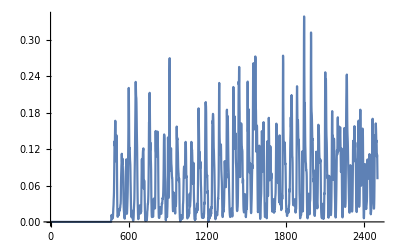

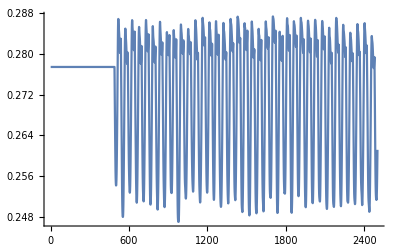

Sub03_(3)hop1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221592.0.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221593.0.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221594.0.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221595.0.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221596.0.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221597.0.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221598.0.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.243221599.0.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215910.0.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215911.0.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215912.0.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215913.0.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215914.0.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215915.0.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215916.0.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215917.0.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215918.0.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215919.0.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215920.0.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215921.0.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215922.0.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215923.0.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215924.0.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215925.0.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215926.0.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215927.0.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215928.0.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215929.0.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215930.0.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215931.0.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215932.0.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215933.0.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215934.0.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215935.0.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215936.0.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215937.0.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215938.0.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215939.0.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215940.0.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215941.0.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215942.0.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215943.0.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215944.0.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215945.0.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215946.0.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215947.0.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215948.0.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215949.0.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215950.0.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215951.0.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215952.0.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215953.0.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215954.0.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215955.0.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215956.0.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215957.0.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215958.0.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215959.0.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215960.0.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215961.0.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215962.0.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215963.0.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215964.0.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215965.0.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215966.0.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215967.0.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215968.0.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215969.0.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215970.0.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215971.0.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215972.0.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215973.0.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215974.0.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215975.0.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215976.0.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215977.0.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215978.0.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215979.0.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215980.0.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215981.0.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215982.0.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215983.0.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215984.0.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215985.0.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215986.0.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215987.0.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215988.0.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215989.0.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215990.0.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215991.0.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215992.0.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215993.0.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215994.0.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215995.0.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215996.0.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215997.0.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215998.0.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.2432215999.0.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159100.0.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159101.1.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159102.1.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159103.1.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159104.1.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159105.1.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159106.1.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159107.1.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159108.1.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159109.1.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159110.1.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159111.1.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159112.1.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159113.1.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159114.1.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159115.1.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159116.1.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159117.1.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159118.1.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159119.1.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159120.1.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159121.1.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159122.1.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159123.1.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159124.1.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159125.1.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159126.1.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159127.1.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159128.1.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159129.1.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159130.1.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159131.1.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159132.1.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159133.1.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159134.1.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159135.1.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159136.1.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159137.1.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159138.1.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159139.1.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159140.1.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159141.1.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159142.1.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159143.1.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159144.1.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159145.1.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159146.1.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159147.1.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159148.1.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159149.1.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159150.1.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159151.1.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159152.1.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159153.1.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159154.1.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159155.1.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159156.1.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159157.1.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159158.1.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159159.1.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159160.1.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159161.1.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159162.1.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159163.1.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159164.1.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159165.1.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159166.1.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159167.1.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159168.1.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159169.1.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159170.1.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159171.1.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159172.1.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159173.1.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159174.1.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159175.1.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159176.1.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159177.1.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159178.1.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159179.1.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159180.1.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159181.1.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159182.1.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159183.1.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159184.1.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159185.1.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159186.1.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159187.1.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159188.1.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159189.1.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159190.1.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159191.1.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159192.1.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159193.1.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159194.1.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159195.1.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159196.1.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159197.1.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159198.1.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159199.1.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159200.1.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159201.2.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159202.2.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159203.2.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159204.2.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159205.2.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159206.2.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159207.2.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159208.2.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159209.2.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159210.2.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159211.2.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159212.2.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159213.2.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159214.2.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159215.2.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159216.2.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159217.2.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159218.2.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159219.2.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159220.2.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159221.2.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159222.2.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159223.2.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159224.2.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159225.2.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159226.2.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159227.2.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159228.2.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159229.2.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159230.2.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159231.2.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159232.2.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159233.2.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159234.2.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159235.2.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159236.2.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159237.2.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159238.2.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159239.2.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159240.2.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159241.2.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159242.2.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159243.2.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159244.2.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159245.2.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159246.2.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159247.2.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159248.2.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159249.2.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159250.2.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159251.2.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159252.2.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159253.2.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159254.2.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159255.2.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159256.2.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159257.2.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159258.2.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159259.2.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159260.2.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159261.2.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159262.2.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159263.2.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159264.2.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159265.2.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159266.2.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159267.2.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159268.2.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159269.2.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159270.2.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159271.2.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159272.2.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159273.2.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159274.2.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159275.2.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159276.2.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159277.2.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159278.2.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159279.2.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159280.2.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159281.2.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159282.2.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159283.2.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159284.2.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159285.2.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159286.2.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159287.2.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159288.2.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159289.2.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159290.2.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159291.2.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159292.2.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159293.2.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159294.2.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159295.2.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159296.2.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159297.2.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159298.2.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159299.2.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159300.2.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159301.3.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159302.3.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159303.3.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159304.3.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159305.3.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159306.3.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159307.3.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159308.3.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159309.3.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159310.3.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159311.3.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159312.3.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159313.3.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159314.3.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159315.3.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159316.3.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159317.3.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159318.3.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159319.3.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159320.3.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159321.3.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159322.3.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159323.3.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159324.3.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159325.3.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159326.3.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159327.3.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159328.3.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159329.3.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159330.3.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159331.3.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159332.3.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159333.3.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159334.3.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159335.3.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159336.3.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159337.3.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159338.3.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159339.3.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159340.3.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159341.3.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159342.3.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159343.3.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159344.3.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159345.3.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159346.3.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159347.3.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159348.3.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159349.3.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159350.3.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159351.3.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159352.3.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159353.3.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159354.3.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159355.3.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159356.3.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159357.3.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159358.3.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159359.3.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159360.3.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159361.3.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159362.3.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159363.3.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159364.3.6300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159365.3.6400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159366.3.6500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159367.3.6600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159368.3.6700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159369.3.6800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159370.3.6900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159371.3.700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159372.3.7100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159373.3.7200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159374.3.7300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159375.3.7400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159376.3.7500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159377.3.7600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159378.3.7700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159379.3.7800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159380.3.7900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159381.3.800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159382.3.8100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159383.3.8200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159384.3.8300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159385.3.8400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159386.3.8500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159387.3.8600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159388.3.8700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159389.3.8800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159390.3.8900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159391.3.900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159392.3.9100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159393.3.9200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159394.3.9300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159395.3.9400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159396.3.9500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159397.3.9600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159398.3.9700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159399.3.9800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159400.3.9900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159401.4.00.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159402.4.0100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159403.4.0200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159404.4.0300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159405.4.0400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159406.4.0500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159407.4.0600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159408.4.0700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159409.4.0800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159410.4.0900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159411.4.100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159412.4.1100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159413.4.1200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159414.4.1300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159415.4.1400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159416.4.1500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159417.4.1600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159418.4.1700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159419.4.1800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159420.4.1900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159421.4.200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159422.4.2100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159423.4.2200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159424.4.2300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159425.4.2400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159426.4.2500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159427.4.2600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159428.4.2700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159429.4.2800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159430.4.2900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159431.4.300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159432.4.3100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159433.4.3200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159434.4.3300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159435.4.3400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159436.4.3500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159437.4.3600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159438.4.3700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159439.4.3800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159440.4.3900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159441.4.400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159442.4.4100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159443.4.4200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159444.4.4300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159445.4.4400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159446.4.4500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159447.4.4600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159448.4.4700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159449.4.4800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159450.4.4900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159451.4.500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159452.4.5100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159453.4.5200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159454.4.5300.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159455.4.5400.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159456.4.5500.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159457.4.5600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159458.4.5700.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159459.4.5800.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159460.4.5900.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.4268551600.24322159461.4.600.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0080466512545704480.24322159462.4.6100.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0121141526044444440.24322159463.4.6200.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0171858813311750150.24322159464.4.630.00310783760242370860.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.021152020698551470.24322159465.4.640.00549625261865661650.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.022363695174354580.24322159466.4.650.0092999581173866480.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0204542638182395460.24322159467.4.660.0115281873537018320.2774651300.367170200.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.017183248497394670.24322159468.4.670.0099605181343497920.2774651300.36717020.0053551408719679470.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0155956120455853220.24322159469.4.680.0087646183512687260.2774651300.36717020.0068457592877534310.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.016061980025507290.24322159470.4.690.0071495121359522760.2774651300.36717020.0092896484730548810.3812648700.2664262300.3076312800.5113005500.282087100.3994901300.426855160.0171660789904221340.24322159471.4.70.0051749471465016950.2774651300.36717020.0143689235241440720.3812648700.2664262300.307631280.00132299270131120840.5113005500.282087100.3994901300.426855160.0189650752714798680.24322159472.4.710.0049119634466382190.277465130.0129819527844329250.36717020.020533198410985220.3812648700.2664262300.307631280.00218216131429468550.511300550.00212169562357957370.282087100.3994901300.426855160.0206306796776345170.24322159473.4.720.0068599634752405670.277465130.0155026343872645910.36717020.026313190597152380.3812648700.266426230.00136355864690882810.307631280.0036267782126807060.511300550.00314844871633933930.282087100.3994901300.426855160.0224799825148157480.24322159474.4.730.008766358322729760.277465130.0194468989863651120.36717020.0324960714552808840.3812648700.266426230.00151931697317088020.307631280.005586525270139120.511300550.004962897191772110.282087100.3994901300.426855160.0269568834034978960.24322159475.4.740.0088699967488825360.277465130.0233389577362294040.36717020.038272265831190710.3812648700.266426230.00184150088628809630.307631280.0074738974785375330.511300550.0081906484496937530.282087100.3994901300.426855160.0352872715506062150.24322159476.4.750.0073687029999906050.277465130.0318437258324841060.36717020.043922479445130870.3812648700.266426230.00219421668880726740.307631280.0087655195439026270.511300550.0108621895234626060.282087100.3994901300.426855160.045685761864598550.24322159477.4.760.0072037958480836550.277465130.051635791829689430.36717020.062337560020734280.381264870.00562371502871420.266426230.00252817438861003630.307631280.0097195180669551840.511300550.0111946491219092650.282087100.3994901300.426855160.057041337914668780.24322159478.4.770.0109348617183529580.277465130.081939348650282640.36717020.116496559878724150.381264870.0165272466352178460.266426230.0031678725586003360.307631280.010619731338838080.511300550.0116571979561731640.282087100.3994901300.426855160.069633069702009820.24322159479.4.780.0170280501884172120.277465130.125271360903740660.36717020.19147899241297260.381264870.0371432445621479660.266426230.0047999482778314240.307631280.011423389927001110.511300550.0138728830650370690.282087100.3994901300.426855160.084001367145189690.24322159480.4.790.0221436130424979320.277465130.166062565971364120.36717020.26222117622757460.381264870.059877005092931050.266426230.0075696006917790660.307631280.0124497625102152830.511300550.0172330650732941820.282087100.3994901300.426855160.09811437401996590.24322159481.4.80.025214592801466280.277465130.175414405298265320.36717020.322949927542021060.381264870.071891582675911860.266426230.0116104153361933850.307631280.0141584706886167970.511300550.0206577418770172820.282087100.3994901300.426855160.109338449972811810.24322159482.4.810.029262289121153460.277465130.193408106109549530.36717020.36362906531756210.381264870.07341278778484620.266426230.018594217259645960.307631280.0155368528294453720.511300550.026034205695824690.282087100.3994901300.426855160.117733527481393210.24322159483.4.820.036859182169554180.277465130.227727116946373820.36717020.37815379443701870.381264870.081341157916399190.266426230.0285869480698596050.307631280.0173204695804659960.511300550.033250316169601520.282087100.3994901300.426855160.123609410918736020.24322159484.4.830.0410190750140738550.277465130.233283834666738160.36717020.32162608623604310.381264870.085577853034956060.266426230.039153221766196670.307631280.0231800083427013170.511300550.0418592453388149450.28208710.0077061078574741180.3994901300.426855160.125435914880265810.24322159485.4.840.047580628863156450.277465130.225989843533734890.36717020.31170975274910030.381264870.083696125185317020.266426230.048566466487286730.307631280.032753523827207690.511300550.049364563102786760.28208710.0088900217238266840.3994901300.426855160.122939399355528180.24322159486.4.850.063219427282913090.277465130.199087816343455380.36717020.34835303116708140.381264870.08646705351282380.266426230.058338060111146380.307631280.042646442304304890.511300550.0559284239485732250.28208710.010291756172952620.3994901300.426855160.121594565340264080.24322159487.4.860.083559717546003140.277465130.163912679253980840.36717020.28631027390538880.381264870.083571270756595390.266426230.070601450450067010.307631280.054236723759980540.511300550.064608451947408840.28208710.014246563074105410.399490130.0029518105218266710.426855160.132712721217214340.24322159488.4.870.103551287934048140.277465130.133731644115852750.36717020.180443899983213340.381264870.083980797256097250.266426230.086307152141711770.307631280.071835807916719230.511300550.085430417955760760.28208710.0196002952914418780.399490130.00371596571010462130.426855160.165090640310579160.24333477489.4.880.124098731159489690.277465130.106217488190165090.36717020.124866434805142280.381264870.101509811384466050.266426230.10727364464047050.309779710.103797314187832470.513191010.117762221222961440.284092530.0263149424993361430.399490130.0045923441615244820.425075630.21478149664202230.24361056490.4.890.133084077221604260.275026790.119255937854363680.36717020.120921568312630660.381264870.158484503020881660.26925770.14049272627852820.311871980.150810239552449150.515138490.152172124598373730.28605260.03741585354156720.398282130.0059299215440760250.423095270.269912942307098950.2438547491.4.90.125658154070662220.272058160.17172556038376160.369464220.159114036230204040.383481240.276465802526929870.272577750.188095288363080870.313671360.189992747987861560.516817030.180339475631141670.287743690.0496496112709022760.397204790.0076056901593382780.421323260.3179552995066350.2440505492.4.910.131806817610388980.269277530.240478114880037790.371469450.239550980272861790.385410830.4141148557621670.27556180.236154046855144770.315361140.208643777471815140.51832510.20120026652205240.289336450.058312441350822540.396226630.0089214528742670180.419666930.346870063393184050.24431742493.4.920.14609070333286710.266507970.28884230811027590.373386580.32740707196304880.387249660.490960495894968430.278414440.26999145315374690.316962740.227175412826200520.519725770.222553413477047190.290851440.06386596772021390.395269960.0098197483497850620.418063260.3515008107495490.244521494.4.930.15951591185547070.263853140.31688416050711630.375090160.41119440381869250.388873710.50402185476870480.281038450.297977301779309530.318519830.261973474008301230.521036230.245916032406001520.292330660.069398315442575780.394355380.0105259254088604130.416537070.336473566996475960.24462651495.4.940.166871598514459850.261338530.325330753827849430.376562610.422610097629006250.390264580.46123746474029520.283425640.352607938962202160.32005030.30407482965246670.522156920.275488102580417950.293792070.078087769661041710.393664320.0116178150709659220.415264730.31157373804857840.24483428496.4.950.16453413082715690.259094240.324632551443073350.377695360.37815997316282360.391314070.408362188137104450.285476760.44096690631738510.321554930.34701579284235850.52308990.31205491127181430.295236810.092120068807842850.393181610.013155586083485160.414236020.286775349564103550.24516725497.4.960.153474516092600540.256969620.32151089282416180.378594230.35984230986613230.392120930.414677121690655570.287350590.52467532448942070.323107630.38707855791752390.525844430.323117879407527060.296735940.110721001059128220.390167610.013960775703327540.410575970.270962279564282540.24357171498.4.970.13896579170646860.255640330.32790310358995030.378895270.377515747715800430.392342660.47245447664184360.288489870.5591683513556140.324363410.40010739906551740.526492180.29859231269193250.297954390.137146189087651170.389916330.014028062136763280.409856770.27458857707913470.24418289499.4.980.121161874264911650.254806720.324625250987221670.378949070.396515281448798660.392333120.50443850214483520.289191490.52862845469715970.325290750.36548733353012330.526920530.254827568158039250.298857540.176785802669596340.389791960.0152481806911198850.409369560.30539161850831370.2448272500.4.990.102298863030699310.254330960.29297725340115470.378913750.39418558829110490.392254420.47610460982243890.289587520.4564504128799440.325887240.30390356952362640.527209620.22900308721156230.299439990.22315650028832390.389738340.0187094832734846230.409036110.35469187414075580.24542809501.5.0.099859331766754230.254137890.316407593348699830.3789190.394157015709869050.392243430.46630864887167120.289747330.37506554638406080.326100850.24495698803580110.527446240.207356018136869690.299648870.253187564553749360.38959540.024190136361619610.408730580.39877499120879140.24573407502.5.010.11742819850605330.254210960.38511520775386960.378990070.399283135152657730.392327210.489750427430083070.289686910.295309015583680450.325929090.188471862645238020.527580670.167337283436725660.29948090.247294918514619850.389386920.0302602542504944380.40851360.414801231005981040.24568627503.5.020.134091447138586620.254572630.42522429193308820.379065830.39630378972337760.39244030.470695050834438470.289386750.220693637005622670.325416140.131431936783661250.527487960.123040279298258280.298979880.209514386238141780.389273920.033593404040503530.408560760.3916365847887930.24537719504.5.030.142221121583188840.255270960.424256075115283740.379039880.39594444304393670.392469380.404497665284274440.288801970.159409188854774840.324621940.082493056983947960.527087830.085040966310215430.298205880.1738898066649540.389372390.0310537044551261530.408973980.33460981308709410.24495055505.5.040.142811185855715060.25636650.346830620526912160.378790910.466030030620272150.392286640.34556241288819510.287870640.113797781376842530.323605250.048299264836113890.526412980.0560434296304645340.297218140.159982716879663420.38964160.0244519649025432240.409691660.25996179219089460.24442214506.5.050.133921877830216280.257877420.251911937527079740.378235030.58360721635129860.391803110.321155630502839960.286557960.077792382032852080.322424410.0275824372065471070.525512560.0354024735414628440.296075280.156543357515911220.390073970.017893865439814350.410661680.184766004724850330.24387613507.5.060.116639362110305730.259793810.20305278328359470.377356360.56545173952504070.391002060.30218248363583810.284845360.048875181178222610.321078570.016513906269572580.524404110.0218107637842426850.294778560.143940684776776070.390666440.0125175149299665850.411868680.120570200220942670.24333657508.5.070.091316692672393840.262053440.148302073751665150.376198950.38575658271548270.389926720.24087961194692890.282756580.02828497136699520.319551060.0109032565331199370.523077410.0138745316417259960.293314470.107533560639387020.391448870.0082498050170937560.413345680.072269778947249120.24279629509.5.080.062031694686303960.264619620.087635975768823930.374760560.213086495726922340.388572750.157861915568603350.280291880.0154861084722461660.317851810.0077837718682590270.521694980.0086283321599571230.29169520.063232828150817040.392206620.0051007488532071440.414862430.0396306542655778940.24210039510.5.090.036460370634569160.267353270.050432262070499030.37315690.106936167313540780.387051630.088956063506877280.277556350.0081287077722302960.315960920.0062971774822756590.520075570.0049591227764719710.289903110.034124339764370980.393154890.0031259542810048620.416635270.019348964335833790.24146831511.5.10.019514924407236280.270318150.031901626720893860.371274220.0561459759637009950.385247750.0495087814862124540.274459210.0049062482730538670.313881920.00507820724506555160.518418510.0049597517698924640.287941890.018069393294180890.39401730.00232785536011005140.418357640.0081749818480697550.24068769512.5.110.0111143494485822660.273442810.0240612501490533250.369148690.035146847771497480.383193920.0334973852288838960.271046510.00455282644884548450.311613520.0036283199543492330.516643480.0071613548817719670.28581010.0097968733982692990.394886730.00358998294576846860.420103820.0028464075579323610.2398818513.5.120.0085099831042980460.276658390.0215070202884337020.366842510.0266790241428115530.380948210.027222630710225440.26737350.004979815775228920.309151820.00306638928841713140.514775290.0095401514098309540.283505670.0082045972935224350.395731970.0074434267320258610.421827360.0016944815346106830.23904414514.5.130.0083848446014505640.279808590.0185690628869347830.36452470.0222224890244977420.378670880.0241253166412546270.263615820.0060032563547101880.306527610.0033054572104301330.512733840.010087797100828220.281059760.0117002408574325730.396707470.0143410091770376950.423660670.0027739468697569540.23834981515.5.140.0095938397602169670.282756140.0162967568717032160.36234250.0195696761388130350.376322320.0222429312355429160.259957270.0083445970782428350.303817270.00322363327207699160.510570560.0085031203947018830.278543150.019628258672884930.397821610.0250716465711116540.425567610.00386771025409028340.2379014516.5.150.0116164632381135140.285014030.016020546654461190.36083670.018510776331590750.374163840.0215228874514775230.257062540.0106250085027732150.301232850.00269031925834597830.508490530.0073445649072315030.27614240.0288075982019657640.398905830.035868216064972670.42733610.0037923206177018910.23756174517.5.160.0108187141646527030.286415260.0160243026433239430.360196770.017608404227616810.372898380.02212547716473040.255226620.0114313968830731790.298941740.00274205529839027970.50471880.0067796236474768790.27400280.033090132386661150.402739620.0454080610145969140.431713920.0047357645324833540.24002781518.5.170.010146862953038570.28691310.0147529177233782710.360410270.0167331299959223540.372585230.0230129855567250.25456720.0104517645269241630.297190930.00310963369323190640.503112320.0064396838095172470.272354690.038100833878380540.403720930.0574238348948073740.433115970.0060456463535939130.23997563519.5.180.01240750521987280.28687240.0125855756743476140.360854230.016462544890684860.37281920.0233934836780977720.254621250.008815801464470880.295976790.00312834782630057840.501879860.0060145902671052070.271202780.046160812446601770.404514150.064708305410808980.434227960.00681374388994966050.23988193520.5.190.015140989455431780.286391170.0116874492937423870.361661880.017203828885138690.373505770.0225781578222954380.255258440.0069501511597785630.295254630.00288887320563455770.501035520.0052398173850482720.270513440.047548258582468130.405047690.06250244488460690.43500660.0063558273086074370.23960695521.5.20.0142443111411939360.285731690.0117616947403672060.362599480.018989594575132030.374354450.0197664871650092450.256125980.0049821897687567810.294885490.0026109043048952970.50049710.0045157151692231010.270159730.041167646045162470.405370810.056864632090592860.435516960.0055289595619827220.23922443522.5.210.0121243525400263810.285145760.0106566667855850960.363387010.0212085940738901070.375084630.0160739545676366230.256891220.0034296428155902350.294717730.00239204382718354950.500128960.0049089304635783080.269998670.0332048848659848850.405620180.0455398033251242850.435899170.0061573670860142860.23893604523.5.220.0133571729985215730.28470430.0083211254964480570.363963160.0243975653867166550.375625240.012271456021558790.257464310.0021692531303624940.29464930.0026506235678070260.499876670.0046561278927778740.269932910.0249115331071312860.405821780.0293029571645967540.436185690.0085537207664041370.23878306524.5.230.017103096046051440.284333920.0071405729341978150.364418980.0289585360899093160.376066070.0087097202619658460.257942810.00144636075679955020.294689220.00308437158088968120.499739510.0032143174082506170.269971270.017615516365060660.405994430.016855960107851320.436390750.0156505321074613820.2387856525.5.240.0203136269139852880.283886950.009018900639359240.364927160.0352537837467859150.376575510.0065787242253205340.258517420.00125070970816369420.294894060.00295438796723581630.499758650.0019920911161277970.270167950.0118841659401672760.40612340.0103440824555089150.436489020.0303420374666629050.23894249526.5.250.021379833304499920.283328360.0129609077564758910.365527440.04736705494158970.377194150.0068016731327563520.259231160.00156661830605229430.295266490.00266858913963942270.499941570.00163394387997499250.270524790.0079447745262631840.406160710.00769676897272706960.436450780.0532787564794261340.23913343527.5.260.020556282159876120.28268040.0203134216971259730.366189340.069141705103277040.377890880.007878577839613810.2600530.00186426961340820310.295813350.00226544217494087070.500306170.00237330635407924940.271047060.0054117710374025240.406085620.0053077566993918060.436255180.083246553197438180.23932581528.5.270.0196381189201200140.282036850.036833666627668890.366803560.098262395760719160.378555720.009285524944578020.260862720.00186377695908833670.296497660.00196812554731713020.500825130.00475033603686405340.271697980.0044979733558265580.405908220.0028372783409502440.435918470.116232768792770340.23951374529.5.280.0190563121257507660.281418060.061988206351895280.367251280.13688759323176440.379167440.0147952613526475580.261635130.0021368774352752070.29729260.00185257382710571550.501451630.0085416655762165820.272450790.00484002517783833650.405666610.00205885186659171770.43548740.145057089540378160.23970631530.5.290.018724693343935080.280852820.09281897789219680.367504590.19691044905666320.379688360.0251309375632174960.262335420.0032101905994767970.298203330.00158973272896134570.502167880.0121390036274333040.273309360.0055424392208343890.405392980.0037357223906247420.434990290.162602400044856770.23994257531.5.30.0220715018372975480.280437140.124035729688015460.367525660.286310317990053850.380005670.0405487598828663050.262847190.0050865680200574140.299201430.00134247482422076040.502932080.0160841306589466080.274246160.0081765119979889250.405126110.0087860584457170980.434468180.166394275381242050.24026139532.5.310.0234852667807459380.280202480.153605987195279760.367292030.402920117862793640.380088940.0604131163973319550.263134870.0078508995457001580.300253850.0026630634464459390.503746380.019028360087888190.275230020.0159488183235449370.404844110.016961657573269530.43390170.160526270043703230.24063437533.5.320.0236973006992561570.280242290.184818519723215250.366710130.55264915182427920.379834650.085231110838017930.263086130.0111615894363513870.301320590.0056417988046677250.50453530.0217015788725348980.276224060.027368447051894860.404614650.0247494665570940080.433365120.154776297794081920.24110451534.5.330.0272994258618942730.280528370.199124756634614960.36583760.61284841732077880.379285260.100937136344539910.26273510.01512955059510020.302354530.00962162044277470.505301970.027259714493108850.277185320.036121303984275340.404395240.0261380546895482840.432827460.15865473351765770.24160946535.5.340.0289862681003431150.28115240.17525482420509740.364578780.52093255254696420.378340130.09743464906792660.261964890.0199556811965716750.303320240.014520399692828960.50602220.0368293339643769240.278081930.038264326785559070.404186550.0227191023011764840.432304330.173218759324149070.24211937536.5.350.029532807665336810.282102870.127236539134911620.362953220.38081325240792020.377013290.083374281332939020.260779960.0271393429272268580.304197990.0208329782295885480.506672340.0468261848944190250.278896420.036967651605201810.404026550.02056643961161950.431832940.19318242122622020.24269231537.5.360.034653561595839210.283025120.091914585651700630.361382830.250675562455646650.375610170.071657262408933050.259616590.041386170704804710.305012030.029330492606700530.507293090.05409552623161410.279651850.0346839093251590240.403845020.0178652278460097320.431354790.215360025306724180.24320937538.5.370.048386184643300310.282792020.07926712521076540.36118650.156062195013052820.375440780.07237941922184720.259911890.067484492335279580.305926430.04294477194259610.508117710.058729982590906570.280500960.033665502007947860.40341360.0130324196530767330.430607480.242774442926704830.24347343539.5.380.064876481613855270.278975320.075301249786486780.364999270.113659879947043810.379145210.081366967259161970.264625130.107095029913446720.307504730.06881187191029360.509624630.063452394579106810.281969210.0378375576713346350.402520840.0092713448691679480.42917410.28020725235797350.24368662540.5.390.075970251577278030.275578880.102416742411716570.367864060.111484907887238510.381943270.103667092358948850.268624880.15994022455622740.309582870.110707602261063270.511344650.074955523340362720.283908490.044510861564827350.40166460.0090214924825475740.427584720.3242291951985330.24426792541.5.40.083604135599133920.272903660.17610277022458960.369838830.13514078600460140.383867710.154488170734752130.271646330.217614125490957350.311486010.16050360468260820.512992330.108340339147047240.285690510.048647642268019790.40073210.0112150868215824240.425951820.36498495177784330.24468596542.5.410.092210050136075920.269467470.29335500063370610.372604720.195669613392070.38655890.24195051068392090.275361810.26953837438850670.313251170.206775227326139620.514616870.1728133574455450.287348350.051963964740346090.399707140.0137878343843826620.424230450.39774299893121460.24505239543.5.420.097186586275257280.266303290.401963340901475560.374939830.275997374050948430.388825390.349523253286862230.278620570.31599989937076370.314944360.250861633881064030.5160230.250163324549937340.288943120.057164811503363230.398888250.0158705768185534340.42271290.422073150827710130.24563796544.5.430.10627572793610080.263120640.424302114597682250.377199210.35026661226148120.391015190.438795790895787350.281743630.363231540465961070.316531750.29430958856782210.517444010.31563765505018070.290443160.063321205504580510.397905410.0171291202721201850.421082510.43681904895920060.24589442545.5.440.112426354383264840.259955190.40936939308298720.379349620.39638943831823440.393096860.459247836780475370.284698690.405444005952702250.318024610.328546954699132750.518675950.349262904204560130.291859440.068938514014412670.397074740.017087589606402090.419641880.43757305359320910.24622891546.5.450.105895461623198640.256886030.38687794020399460.38128420.362460659157205930.394963340.40507010945699690.287422980.432362785279673870.319488850.35151547598659730.519710060.358646629168083930.293255010.075056018867036350.396484210.0161425607940194580.418449490.42334792902622220.24679857547.5.460.098966564411078390.253828740.333040163703009930.382960010.2795440770872710.396562920.36246052200251670.290002130.463411508925381850.321118960.37479795799371870.52280630.386805739430556850.294817380.086552029001723980.393134940.0155753432794511690.414320680.403583101757189750.24540929548.5.470.097787970404717790.251618170.31208586752857150.383835750.30181819654782770.397363650.3955430599074060.291785410.51917978914976490.322642840.398038345788021330.523868220.42210126927928620.296286320.111105395266552680.392585720.0159742326091241620.413099040.392373489432777060.2462749549.5.480.095632921476380860.250038650.351783133047269770.384199290.42588684589178950.397652350.49110796861055350.293018740.57671876757873120.324010290.403385706904039740.524795870.427268696206727250.297611230.15371447543318150.392145990.016374962479025010.412024810.39331871239573360.24722996550.5.490.097793719567915370.248994970.435237278252486260.384234090.498901353938088150.397618040.60227645312035140.293815370.61294674958116960.325136210.39474434934565670.525560340.421482067253265760.298706830.22022507933184570.391809780.0165124443029848780.411132980.39508375876181710.2481383551.5.50.104109088275076870.248363850.54084748501405640.384124010.52090395418112410.397452260.6949692033461980.294290150.61600213466850270.325957450.395819515562132460.526192580.409482939921988140.299508630.317542015589202530.391508490.01742813575813490.410385970.384679527006631940.24883634552.5.510.09846177343160920.248085320.55406505979157630.383968770.56245883281548090.397261610.73109049663284330.294498030.56729983908497890.326442990.391117105713460870.526775210.37861414988469470.299983760.436638779857020430.391107250.0203688131434329770.409676740.35675271300273050.24912253553.5.520.08839712219114910.247946480.47239345400336490.383980160.63743263808907840.397263340.71085662320089080.294601290.46418522955061270.326573340.338490166573405360.527326780.326511366256097060.300111450.54476455319301610.390527510.0254991151597663660.408961690.315188549384318950.24887926554.5.530.083856944469223120.248013010.37466964316681680.384057940.6946079809650940.397353560.68323542382644830.294551830.335634667835692850.326408710.247875678655466250.527701730.262415219614967330.299950180.60715597608785190.389954650.03279325067385270.408437040.26847660406860960.24823516555.5.540.075297607891875310.24835950.28922154498692960.384095860.6618862849122650.397421240.60765346171005550.294293410.215428951108648680.325997210.16465553115701040.527763890.19401057565198060.29954750.62270878927415880.389607240.043152846725991010.408297390.22269212720124060.24744342556.5.550.064795509038522450.249140230.27244023851881030.383916020.6398761923417060.397283190.487264940777162150.293705350.123902666566205920.325383150.10855397068952660.527531180.138307542352821220.298947690.57438636633386020.389504060.052435470623859510.408519220.17832263482679770.24663799557.5.560.0484988491611734950.250453450.28057116421424650.38339810.6142996508690630.396816250.36747806309329470.292698110.065104336126920580.324587070.061951027530551440.527072360.0609196366989427360.298171950.458623026347100170.389573260.05177181769106030.409001860.135133091062758730.24583989558.5.570.0372740738685561140.252252130.245208984575091630.382561220.46433264634140790.396039460.27591711197263740.291280880.033671645868389190.323599650.037781805440345560.526408230.0326617023197702040.29721270.3300342068641190.389790210.044461616927273170.4097160.095248517632848630.24503496559.5.580.029830001583255420.254438570.19925386285346610.381472180.29187393547416910.395019730.203344811324721870.289498220.017957886083273560.322402160.0234403478789692830.52555950.0163463816726084550.296053790.21397962801208250.390120290.037227705424765350.410633030.061805747717764760.24416363560.5.590.0230918434643167660.256911050.183566071751250.380196670.1922887785990350.393821160.14696870647653820.287401320.0099013722883920970.320986460.0154158148094402790.524560520.0097981473235597520.294690030.131993393453979650.390518910.034068041920741150.411708850.036292554077900680.24317279561.5.60.0182499831980265340.259596690.189698761479479750.378758670.162742475145998930.392464080.108835190372669170.2850240.0055216806116699440.319376190.0110523536636875450.523476950.0081083955471541770.293147390.084111440325396980.390913170.0319213032933086050.412859520.019365746524863570.24201276562.5.610.015792865940080050.262462450.184124811769223270.377110670.1484593323864610.39089610.082287650348974880.282370380.00353860785202474940.31764770.0088849813564611730.52239760.0063638607545829250.291501290.0548283855340535860.391237650.0274632394431272050.413978370.0106257082808337510.24070538563.5.620.0133903379777823190.265332110.146236963843115880.375430390.107056029693791480.389291170.060455653793745280.27958990.0032668020264799140.315757390.0081260939215182060.52114270.00378646762566003240.289710730.034597119918602390.391691090.0211407459327921860.415270040.0076183848911635320.23945506564.5.630.0102891394028030330.26835910.092254203031056250.373481390.061844219046773710.387411780.043132075974260280.276520930.00363260710214367450.31378110.0088657522550389930.519819490.00320266533692770.287846980.020916965499664010.392180980.014538453463690310.416588990.0066272252435306930.23825501565.5.640.0075601264261656650.271514940.0515274989207716240.371285360.036953496597308550.385279640.0283275922900818740.273170230.0040580001074350060.311688420.0117823299584692930.518346350.0042347740649014520.285880370.0140809452994971540.392788970.0089175844051042240.418012350.0060544749746218940.23721799566.5.650.0059271814822095370.274706630.0294500172682041030.368919540.0284337196270327450.382969980.0169246682306194720.269622470.00429789048476811750.309509570.0173113936984517460.51672240.005049450383717740.283839960.0113517786780532370.39353140.0049775255030157960.419544440.00596475052728175950.23637714567.5.660.0052962156290590070.277817330.0181209032475215320.366518670.0262166029850199040.380613610.0116484402921122090.266009430.0049610912430847180.307263590.0250627935054487170.515030570.0050814524017275380.281744620.0105572452066959930.394302160.00261655428076593840.421072640.0066314444551996040.23563497568.5.670.0067958999881803870.280665670.012997105511476630.36425920.0258968798062902750.378382620.0115916036258830080.262566170.0060333983448576740.305072680.033236940025598230.511568530.004511392886965350.279708150.0099642358764589650.397712240.00175174577174538620.425182160.00632475696167661160.23746661569.5.680.0106260438861036640.282576850.0107859827932909640.362906040.0257281921925003040.376683940.0129972434601082780.260183730.006492996804037210.303157490.040036131232772040.509978470.0041911797312940250.277930880.0080921318104476490.39856950.0021031253058950070.426601520.0042260408994062910.23714363570.5.690.0141137422658048230.283911840.0118114622261020870.362048940.0249446360097626480.375421370.0149872366753372180.25848550.0067785056016934340.301575410.04584222926000310.508658860.00319153741271821330.276461130.0058256828013492580.399260660.00290618661605447380.427733270.0030255798369009490.23686932571.5.70.0177955716017669930.284767780.0137823589331728880.361567160.0239268815959192350.374624950.017180100357115530.257382090.0081608817545045060.300391490.046455536321921210.507666520.00376989950013287930.275358440.0042785320228879380.399744970.0044738850255707450.428541520.0029163295014816160.23659712572.5.710.021716501407761650.285010980.0148882094381174270.361600690.023290201078455590.37445990.0189235253408779540.25706650.010859635508630880.299704540.037709147087269120.507086470.00597558583352554050.274716940.0038070848705600310.399961370.0077523401111116950.428975080.00296005621535764230.23621312573.5.720.0280356177937433650.284683070.0156702128638374250.362138930.0228332050719494560.374901570.019600218642438890.257491790.0152570698171929170.299450140.0268065613070195240.50688590.00737500545830664660.2744790.00289661592653970430.39990860.0101339259436614270.429060570.00324658911857658150.23567545574.5.730.042558786414514660.284047380.019127882310336150.362914090.0219268793353619080.375657550.0189035793581405560.258311530.0208837505273322330.299497250.021084642146970010.50692420.0077449420145699440.274523080.00198047674272530370.399755410.008587391143502390.428968980.00352308635907347830.23522345575.5.740.06452684850242640.283535050.0236289044727609030.363463540.020431129790661580.376238970.0169352540046845450.258967630.0245047371843125050.29968310.021958446378482370.507082390.0080995778565279480.27469690.00270985862171554740.399558660.0056257465761189160.428790280.0036077799977628130.23485365576.5.750.084810120096812270.283179040.0267353967805253230.363767480.0197216536532171840.376612910.0136713146522970050.259421140.022758042401164670.299966780.0277244557636110860.507328980.0079629867729543970.2749620.0026333187924813250.399345750.00631339646499447150.428551130.00385618942543726260.2346185577.5.760.091255964790107990.282806780.0287905957688132170.364045440.018376250049717140.376987240.0100893565704561760.259893220.0188740714667128830.300340180.036744334760525170.507658470.0073799660789839280.275310570.00153567322761531070.399139280.0127390843411465080.42826560.00540924381264072750.23456582578.5.770.092521096969548340.282335820.031777476343501490.364406590.0163758945027887150.377462650.0082462687037267950.260487360.0174707811296115550.300787520.045408609339145630.508046070.0078106114513242690.275727670.00189562106873301550.398956290.0257774042702088660.427955710.0105562480656823890.23469222579.5.780.102944098054521180.281750460.035299304856484830.364879640.0177083674514835720.378060080.0088732497286969910.261220960.0171483814016190170.301286220.046760952078431690.50846530.0099665018133447430.276192070.00657228730075003560.39881430.0460179896815523860.427646270.021080793189505520.23499045580.5.790.103272232160206990.281065470.039508059994364880.365451780.0267288506491256020.378763430.0093064600722338640.262072560.0155426368446292120.30182090.0381022589271001260.508881970.011301225046643460.276689410.0155202871890641260.398716890.069219403376371470.427361090.0367940487957718960.23539138581.5.80.081176997541042710.280383570.0415012824439455340.366036720.045935791464820060.379465030.0091179978868339460.262912940.0125504859987133990.30231040.026098285662357430.509253060.0111557170436928780.277144320.026220472191613390.39867870.084470962783387160.427130260.055726506943109790.2358843582.5.810.0474532560889222650.279667280.042813016328397960.36664950.078946351203645490.38019820.0141315769804137330.263787760.0091487699145728580.302814670.0167733165076866530.509564940.0108634341454265230.277612630.0363775565828558450.398732360.08553191935397110.42698610.073802206397120050.23647729583.5.820.0225763804159326040.279031480.055336915655468580.367188730.128844768505844450.380843680.024429430270923960.264557460.0063221748164993040.303259960.0119223301631965830.509792890.0114325142079415580.278025980.042633129610958870.398878090.075701772874757270.426940790.086317298967601760.23715852584.5.830.0133378486313229410.278498890.07659698748652940.367623420.196079565503166660.381375060.04044910892359170.265197250.0043855579720391690.303657460.0098837851013558450.509929370.0126402050710214330.278394860.0419486102370506060.399116560.062791167416357760.427002540.091338819952197740.23789196585.5.840.0148960180864302140.278149960.104451425726997810.367869420.28193017582555330.381704080.062391656526479580.265613980.0034196141843021530.303988050.009348763628818020.509969630.0128729363981649640.278701620.0354208795639442960.399436030.05217245557867790.427166280.090725693052726890.23865449586.5.850.0199458782677956050.278058690.152153306987333340.367848020.35123250108150860.381752110.080596138874101890.265722660.0039630746853826120.304237990.0095641693956780280.5099270.0135449143530755460.278933540.0310465496042419440.399805030.04334808092834030.427405290.0896204122227130.23940805587.5.860.025953736666450380.278258770.190246894217159070.367514770.39624130308128710.381478970.090139910517181450.265484240.00697994530582876550.304417520.0106610511140189330.509823290.0172020926517543230.279100130.033942710290474190.400202060.036527945083631210.42769380.093200432775379690.24014693588.5.870.033524833054117240.278714430.195227679702467040.366893720.426762484897332870.380915020.091368524427302030.264938870.0132973003695986670.304559690.0138925461256208580.509687350.0231949078382455150.279232050.038703086479960520.400605980.032877951508248430.428002460.10203532038040680.24086498589.5.880.0408914725956352060.279437010.215207275781710760.365950490.383296470413207360.380006440.081453309862300680.264067270.0252518083408445550.304697110.020741142255293950.50954330.0329001675974473560.279359570.035939103726542850.400998630.0292992455421680030.428307810.114153782358499980.24154187590.5.890.048641170079161670.280268960.246733808653576860.364850390.247970903582554030.378948050.079303500941926440.263053460.044391435183626060.304869280.032885459219145290.509461270.051417058473895280.279519350.0248721038909469930.401323820.0213733565422441280.428536440.131013600559807460.24216798591.5.90.062520199936507630.280289330.230044983538738420.364536610.126290968907659870.3786590.100494331969294970.263028510.069588264844082440.305415210.05059626442104630.509802260.080792854273536250.280026150.016077654292952650.401280920.014134324649261550.428313330.15724670604203010.2424972592.5.910.08321419319451410.276906220.194825082060087860.36756310.090111821473880050.381627930.140202662358016840.26708360.097148293076925350.307331120.075804786644779080.511466050.120714061062612940.281807510.017635643744576960.400398960.0117740242530556360.426807060.20114509407992420.24282625593.5.920.102478975179021640.273744930.211215632081158120.369726040.113737643579116050.383758050.208569905485827130.270708390.122836354306907920.310035560.107006427491800460.513669340.165877094142882870.284331840.027073150829981360.399306250.0127508008907550740.424784970.271776412717462060.24344117594.5.930.118706408863461950.271208760.247846170536605350.371227320.170275015843467380.385219120.308154458812884560.273502130.144361557430472630.312354920.132155130219871080.515607550.204352966892050620.2865060.036700145758630570.398263570.014304256665608440.422867790.37054759308705510.24406145595.5.940.13985637988836830.268266990.27064079626021950.373174260.219084201051671480.387100810.392125978089566450.276616390.160607586619714530.314423310.140867921863072480.5172110.229684726184572060.288451840.043841034618458890.397461840.0151226510321901130.421240880.486620898396816770.24479505596.5.950.172088897322365930.265604340.26049377218887360.374669980.239047712877537570.388525420.42462147208477790.279319640.172500325614929450.316472270.144673419526567120.518651880.256973367915000530.290386860.052648915279197260.396776320.0150921758157785690.41972440.59821813276852950.24557419597.5.960.206495687739252920.263040850.249048712060552260.375883560.27791022030814330.389653850.43641123490404150.281819950.196085406568048880.318574230.17136806119939720.520080650.314429364425471040.292382480.064957645720744350.396068130.0150347168990808690.418157810.67848714996651120.24632752598.5.970.221043215786506850.260689660.25675190873567720.376778110.291179208747687160.39045030.41837694873541570.28402630.261898843001987350.320654050.237648019848222980.521409520.39641953282229240.294370840.07941890759719270.395453780.016170552634218950.416700750.70706491742614490.24710612599.5.980.209112712814459980.258720750.256256996796655260.377271490.230833039258810660.390836830.370318444785039840.285810910.370684267447357660.322631810.34113262394313230.522607430.477110192241972260.296275670.093689736843489680.394939110.0188926297127677940.415394920.67846581364760320.2478875600.5.990.182512663062365380.257216320.238312503446917760.377320920.196485318706852430.390771670.33315203630255090.287136370.47366559992513450.324485140.43837314589831760.523678710.50847940749279420.298072770.105171430362997170.394507770.0213543878095719850.414218190.60263743895797850.24869862601.6.0.152902768227416330.256102310.21443301411138560.377121810.22945239753138180.390458820.331360070750140350.288096790.50723768580931340.326076850.476244815313234150.524553360.480160000860665240.299625390.107312255480451810.39415260.020431792990548180.413217950.50226138430182210.2494604602.6.010.129354160035245660.254886360.282439174974500550.377155530.31851062946571320.390381370.40408385709706830.289124880.46400324770387870.327409760.464256360368150.527394260.45475961150007860.300932360.099899233056826640.390946050.0164464600339374880.409328120.405396969977200040.24797377603.6.020.120086236655134920.254111170.44155331842015790.377187920.42664167388042160.390340330.53031607265255450.28976940.41727712618235580.328205950.439097407815322470.528077680.4580845683147080.301716340.097772183170980630.390396090.0132979439727628460.408418170.33210831746223540.24819552604.6.030.121463058992799410.253439950.51888926002015650.377456730.51668822459751950.390569740.6097573432203830.290320670.4112158475926350.328598160.40786450395634130.528723780.437585522779687150.302103530.116506869787760310.389708480.0126638079215333120.407520690.2840041640236020.24804728605.6.040.122032446162856830.252961770.459595315020732640.377841530.59342656892033510.39094770.62470306259669350.290709560.40999128506573040.328651630.35037345319899020.529320520.361035862714505440.302156370.1657931411265520.388935870.0149456661991482360.406671960.248838674244793030.24757272606.6.050.116689064919305820.252718910.366722706504807370.378236080.66192190647092850.391360540.58625716694382470.290905860.38940281781530820.328450370.262600569990085350.529786230.279194000015999260.301957550.242283464991033480.388202980.0219877467412862430.405983790.215606868555403040.24689907607.6.060.107982246994865850.252773260.320364898766435650.378533140.73970302207626570.391694410.499288311565834030.2908620.35260461027151340.328051080.174561537722818520.529951120.224254361019995440.301563640.337120224278778140.387753080.037443196355822680.405693980.181570192136272870.24624209608.6.070.101716011189603730.253204180.34688217883317610.378630030.81124309129466290.391842350.391191290707044950.290512810.303814145592425140.32748150.110902166966943270.529778530.170690115045380540.301002890.41832521344543110.387644480.062953475199624640.405851370.148909605162274580.24566779609.6.080.098662910102514890.254022590.391692942125424550.378510260.71980577054515330.391786560.30714749066453580.289842510.241828801454622180.326732940.072012511036112160.529359910.111930185616900920.300267890.43288545766208050.387738490.086522355055650060.406312970.119447120662154180.24507227610.6.090.094218180557944260.255270320.418276660703196250.3781230.51431166944123030.391475090.270580682861175760.288802510.172524402525471880.325794010.047105990569620230.528706720.064758563066787750.299348880.39096618802826310.388024270.089045955160814940.407055150.093879609708636750.24449047611.6.10.082685570202000320.256917710.38879193573166440.377487380.40260145475347120.390926590.262831679924367350.287395560.108912108723643680.324636580.0296033557447302650.527830490.036025799947440390.298220130.31870468139576090.38847580.06954162277455550.40805310.072319014713342520.24389597612.6.110.067153722085628980.258896920.28279480173292650.376643570.436972083107261770.390178990.253582616973811460.285653550.061118856385312860.323249190.017729779449626020.526746750.021170070087142540.296873030.230120340528470050.38906310.045607507070751510.409281260.053714363900001870.24323901613.6.120.057136232639795270.261430650.184110249243071430.375386130.41192286823778060.389029940.22602193459453580.283339850.031156695035704790.321565470.010536852133268090.52359470.0133930747178930550.295246970.155791793299988570.392356050.0284086782058980170.41340890.0375728383989723460.24457125614.6.130.0434392989090563660.263887250.117263393368782470.374164930.254060776643376340.387910570.174848168151656770.281005420.0152782950819416160.319788980.0068323432809574760.522262390.0093755420925915860.293541960.109349809197161270.393029610.017652998952869320.414872330.0243489601053739240.24373413615.6.140.0282005204691916540.266523040.074285499206664910.372753910.109585624653828050.386598470.115681006571195550.278399240.0079751754534919570.317866350.0057533301021006840.520831260.0078335346426307680.291709010.077718105375546980.393736690.011029972332695190.416423990.0150666084298079990.24285005616.6.150.018245823439786530.269344050.0526465090935590160.371104440.054484286845043880.385042490.072144532785387040.275491820.00563673127095291450.315806120.0055055287277350820.519273150.0067984241136472770.289756780.0514490117034971040.394514980.0074878915797305820.418078610.009997693658317720.24200661617.6.160.0120872790371135390.272404580.0419494701822358260.369133170.0432447549310031040.383159410.0492327732164110350.272197490.0062425730463418360.313575630.0055994760002736880.51755280.0058624535243578860.28765360.031989267828534020.395368620.0061864845507592570.419831930.0081294525526922760.24122525618.6.170.0089494674011010.275523560.036266151690239110.367000390.039337344390414790.381103610.0380871611653446350.268688510.007291749247156880.31118460.0065146475741056610.515585990.0053177188638990590.28540790.0213096875475909250.396436140.0058608587116011760.421793890.0079687037912072980.24066392619.6.180.0077427312260310730.278670760.0317195218885729240.364739970.0365469574154834860.378905760.03281360471619690.264991270.0074731298562379020.308632730.0067430399604675650.513512640.00492858200359826050.283020970.0178890951001577330.397505520.0055447682022455530.423748320.0073666082762146550.2401185620.6.190.0093660697970238820.281552810.0268879540806445940.36264240.0335975576209088040.376845350.0295483959023383380.261467450.0077503401394190310.306066950.0052889695762597680.511293140.0043117923795177530.280631530.0148119136112493270.39875820.005081457178981890.42582510.00655471334961633350.23982552621.6.20.0155141011802276930.283816350.0239001056257433440.361123510.0313302590936046440.375097890.0272403386876883430.258607890.0088225105727474350.303620530.0042462823510530140.50918570.0045316507184798480.27836060.0121755179692623690.399918230.0049951157419133160.427715860.0095288320305252270.23955209622.6.210.0186770275845226650.285362390.0228140492636857360.36026210.0301605775161753120.373689320.0260296613864671660.25660890.0097094579670023250.301501360.00407669823438718950.507311870.0047453047145883940.276392250.0113896747143490860.400957160.0061234760211552150.429354380.0181242894451762340.23931119623.6.220.0144046064296349060.286330930.022527651466291630.359870010.028269243229646030.372841610.0261012331061643740.255337950.0089822157958996550.299826120.0054772116395147580.505812230.00522824210899328150.274830580.011318504620464370.401760740.0085299805464913120.430619840.031864182565009560.23901733624.6.230.0110252121888634280.286676910.01987839748284670.359992240.025014603665981050.372626820.025648618050900310.254880510.0077373643149348890.298678490.0087548707672705050.504769790.0055896121812671110.273755840.0104851038638432790.402257570.0091678361904872960.431460710.049549871447414430.23858948625.6.240.0099264743426674980.286422780.017169925733011250.360621330.0224404986960901640.373041590.0245929402292428060.255216690.0078566540201125810.298048210.0131941817633462950.504174550.00661058166351757150.273163390.0082565521166527730.402462410.0074436092930283110.431911370.06992745864045070.2380277626.6.250.0080152720257223620.285798980.0164279411805386480.361522530.0219522081538535420.373834550.0224178302383966460.256037770.0089241632392170440.297821840.017852290081413520.503918630.0088372710926266950.272950180.0063997617938079090.402484060.0064012057582606810.432090180.089205640703029870.23748087627.6.260.0067083450137518590.285205740.016048760553520390.362264720.021306707081964350.37454820.019060227127761760.256813120.0111252500857295170.297838840.02392584376374380.503861690.0112040259987751710.272966210.0066930647219587380.402447340.009084644895070930.432131820.102721526098927250.2371127628.6.270.0064018824075104040.284817680.0152808981691420890.362669680.0201921036062793840.374987610.0153920639537999580.25731740.0151271030980018160.298013590.0311041805955400950.503956280.0122677918716092260.27313080.0088248799058401850.40236460.015223588665441280.432059230.107275774055457980.23692646629.6.280.0056743004357162560.284481880.014499955962525710.362946440.0197454632646977160.37534190.0121768754691738680.257751910.01900830927855670.298314470.033096088407604740.504176650.0111764162508797280.273413870.0094557794513957690.402239650.0232338394516499350.43188850.10209202554123270.23687996630.6.290.00387449474231381460.284093050.0155624706020276310.363243580.0193171048338625740.375742260.009328934926975220.258252850.0213116617772604770.29870720.02626156870483160.504478050.008986162729956280.273782780.0094748610379871560.402113290.0309575205821818740.431667810.089231737527469560.23698556631.6.30.0020461159943659580.283637770.018442758377016860.363585230.019126299210282640.376207480.0078692529719425560.258836410.0239787250984091450.299174350.016598666468750730.504840370.00761316661152925450.274220790.0100710237676096360.401984890.036794679166637240.431409110.073124147429809130.23719782632.6.310.0016522630333851450.283150240.018628823876821180.363935810.0236296427351076060.37669680.0078459421334092440.259457730.0278983109727713660.299698630.0099452167107207320.505230010.0068456286310940310.274711420.0115646138959941830.401877410.046389986995947540.431145880.058523415243214370.23750411633.6.320.00229623120073523020.282621550.02260718401651860.364301650.040721700784883630.377218330.0091696257823057240.260127310.030853604230014380.300287370.0063287990378475460.505634150.00547737930026095250.27526130.0166500642882160650.401805930.064932487897690650.430898890.051163525055084880.23788071634.6.330.0035900346236638290.282138660.043193717579051120.364622890.085543179867457960.377686540.0127612301631592810.260735060.030885237531778290.30084270.0044168451790860040.505969130.0053719006730875870.275779080.0255168001251310330.401818250.081551063663711730.430733490.057518770787791880.23834795635.6.340.00564870501763018160.281679930.085403803355535840.364922280.15520572333858260.378126130.020329236259249880.261308990.0277641866870176060.301374170.00386733091174992080.506229480.0070284041094346580.276273910.037544435082647380.401927820.081402969322310630.430665650.07720192243014670.23889979636.6.350.0108141278379292990.281234820.136088736726005440.365206270.23513605043105120.378547810.0347948322167115560.26186270.0228920368232657070.301895460.0042443873618708750.506419990.010012150800313840.276758730.055254919729176780.402142590.073625258976062480.430698420.104227672601359120.23955639637.6.360.018037914420850810.280863730.17827982625377180.365406630.308437920354594440.378881650.053862020209283130.262321950.0181207700277177040.302395970.0049832502744291210.506547760.0134825304212303830.277223810.07383814060524970.402438730.069541534068852650.430812770.132431878366650740.2402859638.6.370.0236497260924201470.280751050.201278634468123160.365315660.325824992045205930.378918670.067903054758522850.262460970.0147654387458081310.302843290.0056703443626078660.506607550.017046556589061950.277639210.082934005065653140.402788250.066644834790451650.430993890.157878033760081470.24103359639.6.380.0278962907500741670.281060570.20136923109089590.364749830.345603767001795350.378473790.074597939897898510.262078620.014309081952404140.303206870.00666181774103397850.506611120.020734063272505380.277976710.080185388145196270.40313960.058733281204680090.431203730.180440120832065340.24172165640.6.390.032672663290767550.281776010.231537615595689580.363722540.39379995603927520.377562110.081082831836580780.261189050.018086813143194360.303493590.0090646393362488150.506580790.024750534827672870.27824280.076269117621437950.403454330.04973641444931570.431407620.200799458866797680.24230177641.6.40.03800685248127640.28270640.27783431406784920.362450190.399736427807644230.376401790.0935199395287850.260020150.0253514045453533430.303728730.0127601974140885390.506552640.0288388986762811330.2784610.073239531009243640.403720020.038257183172722050.431578180.215658759702233830.24280198642.6.410.0522254667328805950.283593610.2844074215422190.361217240.372178343058235940.375284710.10793252058467180.258892850.034271266788358460.303976270.0180758347224339660.506583580.032914762743025740.278690690.059554528247210140.403885550.0260419664063898450.431655130.219816865908630620.2431771643.6.420.072390732319866330.284428770.2614750501253980.360046330.35066798835885190.374225550.112845524001690730.257820470.045976451675524420.304216660.028042366550495780.506712590.0389131935807094650.278913740.041472757442546540.403929560.0178234996590728480.43159620.212670369114133530.24349746644.6.430.08875822430573020.28389420.200362471393057960.360450750.297214909712615550.374707840.11688073822935970.258508130.065578672822305960.304723690.045501096717129630.507205540.047112910239135930.279384240.033047536684610290.403629010.012794412955691310.431136180.20413102781636330.24352748645.6.440.102095827494233330.280205410.126038055617892360.364169410.19981797651275280.378323190.12424303048622290.26313130.094404621492233790.306292690.069116043560814480.508735960.059795923062886680.280841340.037311454615908310.40267250.0107990439379293670.429678310.210714968123929950.24357808646.6.450.120717681630573730.276859460.103070820912173620.366926010.124301061764302720.3810250.14163462037768060.267138380.130238858767538160.30858160.101891448160834440.510610940.083460561565412460.282973250.048961805116009150.401747550.01228092771913230.427998620.243077971803263650.24406211647.6.460.143721706650400650.274044840.164918170725351750.369135630.095863130982251150.383183520.1841179737897110.270371320.17420378196741760.310461470.14633663506673710.512365950.118912028162121640.284730460.064410968247942820.40065940.015737595833628450.42623430.29805669965262790.24431053648.6.470.163556690647664570.270879870.263642236726954750.371680870.113159417688969820.385663640.27768349193641920.273857010.229463649943107220.312211060.196537566887058870.513822170.15975704949496820.28637090.080866148246766180.399854710.0192383150866941540.424761580.36230576538641970.24486328649.6.480.184746548862313730.267994860.33071238026760390.373708250.159793390097550230.387630650.430233358791105640.276897690.2972190376069310.314045510.2606058081604440.515434540.237173670268523480.288095930.096739965330608760.398787840.0215779167783091730.422996580.419782976626754840.24517094650.6.490.211871349444722880.265228790.3551195690925870.375430820.259128040882026730.389287860.5990276315060480.279692170.37490665064369090.315920240.34647321001182520.51692340.36570243144853590.289864650.111116619108824230.397874490.023239865045406120.421339640.458022279572582240.24572859651.6.50.231014372446629370.26258660.35654420622239040.376948040.34337561698126160.390733910.66960792079860510.282252650.45193283296788310.317701590.41748638489036570.518192480.487364330254532460.291552480.120423177708872730.397172140.024545759304965450.419923060.46961283949721680.24640746652.6.510.229722743964975750.260077470.36168746539943870.378284430.290793302949813760.391994620.60055531564858630.284587290.5227318843851640.319380580.435423131379119030.519283640.57267355699153670.293151580.124305426844244280.396635340.0253052178072986880.418708710.45154711074600810.24718624653.6.520.218277709358823320.257444870.384105872070536760.379583690.222871479028614480.3932060.492812566705256470.286937110.57578679454628430.321135040.41969628021400340.52251370.60903719764285460.294832840.127816152175865920.393198190.025874480227924870.414450940.406181571206176760.24576497654.6.530.208937927528225540.255413430.38241316312631950.380353590.207251041866168080.393891210.425461302006053750.288681820.58439555797077970.322700690.411069025917900570.523633460.58371879565598770.296342250.13021020313785430.392608840.026088662120637820.413192530.3439891504917230.24652908655.6.540.205713770797560060.253757560.402946511694436570.380880550.22279246051432260.394338560.422057479547139240.29006060.53550975084624020.324030410.40809827867821330.524782320.52455050326927740.297630770.12688353408306810.391839740.0249750853924643360.411832640.283100989108998560.24700476656.6.550.204605356492256420.252485580.4340715178689370.38126360.285612698004211630.39465640.53539561680269370.29109370.445632210241471650.325025380.391256582398960830.525818750.43612786900186950.29859880.11788382468066570.391031510.0227772158199732730.410551380.243965999787760870.24724688657.6.560.196484835110453530.251572170.39611276903082310.381567970.309891443893346160.394915390.66099910620883630.291821810.35175364804066220.32567230.33906229191582940.526642710.327569850510801340.299229970.108873519138723350.390337550.0206434743316008040.409502170.237933023721588060.2473885658.6.570.182396296203674340.250985990.34191776292582950.381815050.3400147168200480.395137760.67668437233392650.292283080.289614956134377430.326010250.256117756348786530.527404170.2518266918448340.299560250.114345777717326320.389594750.021410584042998730.408502460.25615106007519450.24728849659.6.580.165534261642850730.25075220.324424411706569660.381989150.41486767575665380.395308890.67110392888792670.292465750.25736959667653340.32604880.179256125256807730.528039170.207210769490246030.299597960.151196193654466540.388866310.0285442453857287850.407634420.27942506738548050.24699713660.6.590.14752219359987890.250809350.30101356347984720.382134830.457119956195238150.395472180.64256393972113930.292421160.220727454184124430.325804120.12371896019000530.528573510.161502014249191170.299358750.214611491076756480.388061160.045268460903338520.406853290.293717127725260540.2462877661.6.60.134595720280053540.251269080.30361080740460530.382109770.469622897530984350.395480620.59506271670658340.292060890.16711889741188590.325324910.083457676018572040.528749360.115109223169963440.298890860.2726449332318870.387573890.069572220435661330.406532110.29080715119464880.24556391662.6.610.12215226725175860.25212930.33564258358777610.38186470.4935114594407240.395280030.56022603569330210.291379060.11312691401480150.324659830.0543300786592155960.528538360.078185429972338420.298242760.30483302565119590.387468890.086360750118241440.406716320.26878222496068270.24490526663.6.620.099256606371123730.253405610.31192838267976190.381381420.45360327066687030.3948520.50281824448281460.29034870.072611336180214050.32379020.03467484481951780.528085050.052456592132895860.297397560.292837623395525940.387511610.080186005170110680.40717490.232360113462744680.24411033664.6.630.074271994194496650.255107230.26353627414464490.380608240.325388886865222270.394142270.416000054921369040.28893970.0457205027533219150.322739910.0234307527449192780.5273390.035852082579286970.296380170.23354422417083830.387818470.056577178634630210.4079970.187675183358330420.24333626665.6.640.055129752565657050.257205730.220839697505397140.379552160.197823130357907470.393157530.307887847094614860.287145580.0278350431379158630.321494150.0179097775990432650.526403430.026478643880056770.29517830.160700984944932480.388242140.034848038430047230.409030540.139734238497848050.24247088666.6.650.039152949003483070.25954320.173963154161711990.378327050.12118319827964220.392008890.190096472649121380.285072380.015947492955760160.320061450.0159278981756318940.525280170.020971384706491130.293802750.107332177508316790.388802270.0225432581076069580.410276780.094016500124249970.24159771667.6.660.0284965656925034170.262140.151320095736647980.376871080.072430766078068380.390632160.100238378775361960.282675060.0088869584198224770.318466450.0149453048675398330.524057610.0176417405333896340.292279830.072608970051274940.389396340.0151832553203659850.411622450.0563586890236652950.24062863668.6.670.020369909663170830.264878040.119425464574023430.375253810.0517104653144858440.389092850.053969945051336210.280038170.0051882240625827010.316733040.013491771239144130.52273230.0163513977362623850.290633790.048456739165932940.390051910.0100584260570639170.413068760.030054286360408780.23965298669.6.680.011916909420809270.267727440.077603777594137630.373476920.0422449550144240460.387390.035838950366215050.277172990.00405786746063914550.3148580.012820163190128920.521291790.0150167564453385780.288861650.0313643527061871550.390774870.0067010869349223190.414603630.0147501675930515240.23872576670.6.690.0066290214258800130.270734550.048375657375794040.371453810.036083691098416690.385436360.0288239360466928730.274013270.0047861346379981230.312850030.0125305382311579620.519691910.011770727149749240.286971190.0180220877607161350.391627660.0049609370812180180.416266920.00779232877187453850.23795536671.6.70.00450276636956868650.273877670.033612313259990750.369186920.033745662867690610.383233570.024570651084877220.270559370.0062533708709821460.310703310.0114864281567154180.517950720.0094458892206450460.284956930.0095424338249445180.39256380.00514941305069124750.418006470.0058512112326310910.23730704672.6.710.0051772468781209570.276950690.02719571375157920.366868610.032727103354594150.380968440.021542328028959180.267031480.0074965366103913610.308491450.009831989428889930.516044360.0093336538081954020.282889130.0069529541046414330.393687180.0069884189395599870.419896110.0053171770858432610.23692214673.6.720.0083972124733548820.279852060.023965361318444010.364625340.03032223982472870.378762810.0206941607526545880.263562860.0084410458816276920.306243190.0077906157411057970.514072230.0088048075587654190.280795320.0049843115533730760.394864370.009271796854135360.42179920.0040987270747338340.23665978674.6.730.0125088713014915340.282426510.0222796491160984730.362646860.028264046653407970.376669590.021278331745822540.260373230.0093645455596814660.304017890.0061584454979517760.510283790.0058831277863442470.278729310.0033132984100236280.398727570.0120479836365712070.42634250.00346099928060127370.23895217675.6.740.0139155101804698640.28401370.021159686489421380.361660760.027451845198830120.375192930.0215645292370369860.258354790.0097434061433400170.302090580.0061905712077725320.508597530.0032649123368148490.276940080.0041021289963892880.399716910.0153865536599029160.427872490.0036698898942404720.238791676.6.750.0135833821931422050.284967610.0197392941370327440.361246690.0263362618413404730.374357450.021163178378733630.257122840.0088526034547914570.300529710.0078984484026872140.507185310.00267635916680281130.275487350.0056394765338612650.400571240.0161140580433168650.42914090.00402780284064561350.23870449677.6.760.0142886075596712630.285341910.0172404431875234180.361339110.0239386489977184980.374118510.0201885976240176350.256635630.00689882969664449950.299387130.0116857915491263620.506160640.00216688589293745960.274420030.00521250588428449550.401127120.013398363585037780.430011320.0039810038770083560.238459678.6.770.0150109768461930030.285168040.0151561462092042050.361916150.0218522612807320530.37445660.0191412782757810240.256862220.0050277268739233750.29865590.018707525471948310.505494440.00078359829687631090.273734630.00351987026563082640.401430480.0090030957309773780.43054950.0037230144735291610.23807712679.6.780.015775871588919120.284638870.0154256683297774850.362794460.0212380706534590030.375168590.0183993211779793880.257548990.00388956702156483070.298220760.0295700248625554580.505100680.00131050282908985590.273325750.00263032373541143960.401546490.00563574577527991860.430837830.0046712351945823020.23763091680.6.790.0161310446586887470.284133480.0155952579356199650.363552730.020198184851071890.375818670.0168081358148535480.258200860.002638395580858180.297965990.045217699989913060.504858210.0034312614453994270.273085990.00224757172328066660.401595110.0048974907628178370.431010610.0062750263655225240.23723844681.6.80.0182427469863865840.283754820.0141577948156480920.364090750.018317670588315930.376295420.014962426736344760.258686690.00155485901718315160.297834280.059420610471992970.504717010.00469563557553181850.272961910.00148494519028376760.401617320.0060254776033400510.431115760.007865020122837660.23694114682.6.810.0234072370943736730.283424910.013988920160627840.364518980.017331868825691680.376696210.0143210668939998710.259108140.00129339537597050140.297801270.058398434952529410.50462670.004075769975378580.27293080.00234781149523811270.401704710.0111264292930923930.43123230.0127992038522134960.23689034683.6.820.027330013962110540.283017780.016017420998927090.364979270.0184276340357259970.377167290.0135692227354671840.25962590.0015699200953839980.297898820.041218952603652320.504608550.0031523213941918140.273022720.00638580468328463650.401850180.0220207970070250.431346670.022378018513654520.23709046684.6.830.0253456913864797550.282415630.017481418544680540.365595970.025900342850494210.377840620.01124172746583860.260386930.00243244122070086650.298169520.023721376672573880.50469950.00329598803349955050.273277550.0135546827814632710.402001970.0387681683379544550.431411790.036281264168225330.23745442685.6.840.0210455834400169080.281618290.0186239497591875160.366362860.047883460125490760.378712060.009474683927827330.261385850.0033409824489364490.298618280.0135910088292846860.504899980.004398820908675760.273699310.024521142368670570.402140650.0609382508894672150.431417610.053148939979055960.23791771686.6.850.016532694390217740.280796540.0232789598618130850.367106770.092496513772736270.379590180.0112377152298245180.262404870.0035665817003790240.299160220.0093915435750391370.505162540.0062500652912080320.274207550.038237114945326290.402258570.082750610587589370.431380380.070954929353108890.23840645687.6.860.0138060473212701150.279994910.037136404383143070.367781270.16667324493050360.380421650.017783943032209190.263388630.0035893672972751370.299776080.0092880630971853440.50547240.0085100982111752530.274783820.051518206922470810.402364830.093091014264615620.431309410.087460478964942410.23893914688.6.870.0145410867575396850.279220840.066500698137054270.368389950.272092007132096360.381203560.029311928236322220.264328890.004239553646732260.300439440.0112143745162392050.50579660.0110735335334829310.275403170.063037479948835920.402477830.097390294823095660.431234650.100486583677747030.23948866689.6.880.017613777609498970.278547480.112784419592325270.368848590.393719785344095350.381851390.0430617915749605950.265139070.0052484994986783960.301143050.0123139434141594020.506122640.0141233618395640620.27605880.071259002649371780.402614950.106059255741801790.431168830.10851353535776290.24008565690.6.890.020995001563892350.278128820.152467075536771750.368995220.492677436099760950.382194850.054849612826128590.265639160.0059982297203084610.301846410.0109422416880353510.506411310.0162346832436300330.276713130.072949138625204840.402815710.101029268985224090.431153870.11233497856071980.24077815691.6.90.0202942262199078860.278103360.158847233761756330.368672520.51688176550004210.382078970.067865137564722180.265669480.0081390721228653680.302540050.0093563025116612760.50667490.016013530327051490.277357630.07076557655177410.403044180.080248518257365450.431160290.115006942879073930.24151358692.6.910.0160207908618988930.278566420.158201124399274420.367771990.443161104257568660.381395680.092468166667144040.265116380.0144422848684148170.303213570.0097514936626887350.506895090.0167716054282055530.277982920.070373351847062050.403320340.0570540208953406040.431209270.121427113805205660.24231641693.6.920.018055030524149190.279346890.186554726948590820.366482490.30484519459090640.38033430.108325014662541460.264176430.0263864522636385360.303888450.0141960962740290110.507103930.0227705237664710960.278609210.06356992728639230.403616970.040428468686138520.43126810.135278731448925520.2431682694.6.930.0298946653120989170.280210080.190510021722328280.365071120.185223911471270740.379153280.099151851539808850.263125570.0433853304863052250.304585980.0231294036555248530.507333440.033319252207868010.279256450.049423794118151720.403897740.0292100940107321160.43129850.160529298117859020.24402551695.6.940.0486997114661772150.281073310.15441512728625140.363627810.15956581142014920.377779580.094836443346705480.262062850.0624048746761785150.305323170.035003968735294540.507627310.043585609773502140.279940690.035472725202349250.404105740.0205877188803710550.431242950.20345619717266650.24482063696.6.950.069760187070576740.281599490.12779451930835720.362530950.176414769723289180.376739820.102865854189657030.261409290.080968681709014390.306167580.049114733410026480.508078190.0536242361190345660.280725050.0275641371555119460.404123950.01493350437288340.430987160.26742876673959710.24536509697.6.960.087364717279393780.278426140.122096510551315980.365502670.16030793274589080.379636270.112658564548965710.26528430.09909015426490570.307788540.066464043854408320.509361570.066988593372395030.282233650.02628250356162170.403548840.0114895284886454720.429889810.345649216953744450.24571888698.6.970.100912240883751030.274941660.134916035220592760.368315980.126779009944870540.382384670.127067582229757970.269354860.117955844998924520.310087970.088895364569324230.51114680.081866201176831260.284380880.029497613748141570.402747210.0092005522063742690.428306620.41858246940961330.24628137699.6.980.103836360133898270.272385120.18290617790765180.36996020.15367022235472410.383981710.152586145975036590.27221890.140897831244510020.312264890.113672077824013050.512928630.09442289874078930.286421460.0353647752360460240.401831790.0083382112138113350.426577430.4638434394650570.24688038700.6.990.089913994396412120.269116350.25874367651358890.372468490.21596815271058960.386414320.20776892027232260.275731070.172972826981402070.314081910.135064104450418140.51445020.098701086858454830.28813020.040117720803187820.400956290.0083862466419173250.425002050.471297407293421840.24725781701.7.0.079128663185026020.265996990.320255164343139660.374729890.245676853153354880.388602020.310232133239501830.278927850.214337910288060820.315760880.16604601810883990.51583790.114197061150826880.289714030.042458115933186930.400086830.0091622216304006260.42347580.444748637367253560.24753882702.7.010.085405288867054770.26294970.332704612057248050.37680960.284241083513359470.390607740.39703372007486650.281907030.26091969039784250.317365130.230010220753670060.517210890.18668357395404570.291233050.0478811581754179860.399114360.0114413563667554260.421868630.39837963971898060.24769194703.7.020.095114658269309840.26008270.32779559330342950.378586340.309733038102826150.392310.386708854646490850.284582530.308481685605226430.31894290.325762294459257530.518468270.29430825620061340.292733850.058000453007465290.398260280.0153490711526891470.420382840.351102727585931140.24796716704.7.030.09920001762328440.257619310.35352211134048190.379807310.32232669240500070.393452620.312893691363622440.286784540.35649269574642910.320590660.43441484709340780.519654960.38467012176359960.294310010.067772007997668940.397560260.0185780691792989950.419001760.31618414256234840.24854266705.7.040.105716676278979310.255689060.374249396529969360.380340390.33409306431403030.39389580.271339362130514850.288448560.40444900606199170.322370120.54107032600686190.520839740.428398536262429630.296022860.07282449730268110.396987410.0181749929188490080.417664850.29613383415330850.24944246706.7.050.113494677795978190.254327940.38426441248888160.38026040.302811419888968260.393713020.313213612008223230.289590020.44664033947457040.324161850.62435726013277840.521968990.42432547661513260.297758460.075951411287093320.396537780.0149287084774453740.416412770.28844414743384830.25056165707.7.060.118001224168116450.253116270.44280453045282550.380033130.284116173263551540.393370420.39404240002211740.290584260.467373179258594450.325867740.65467943164896580.524924480.420760196829220330.299420930.079130926707713250.393550860.0124710311240206030.412513990.289318347439239560.24980203708.7.070.118237353349044320.252448580.50016269733936350.379594050.32000381185105410.392832290.45531186133394750.291123420.4533028725132130.327141420.62390206855709880.525812060.417782843071720760.300668710.085646544924250740.393133110.0142904471789187180.411468570.29253893450602970.25062446709.7.080.119788869447490040.251920390.52382705004051990.37930470.390526670631937130.392464750.50345445318582620.291545570.41817265125945690.328039880.55010766356087070.52658090.397915255189427660.30155260.10256295156632630.392662220.021113258797188510.410531080.28937123925863910.25106387710.7.090.121328714968979510.251495080.54609303838375330.379244380.50623938975832380.392357090.55094501139039540.291882730.382782543224950530.328543980.46339825207357720.52729680.37184829589662440.302050.13595856036581290.392040020.034611107065619230.409619790.27583632909169720.25102162711.7.10.108412317105746210.251150610.5207237422465560.37942390.61037797925136950.392522540.58649086420335630.292154010.346257267823960440.328685670.37591793255084050.527933670.33354326770383720.302190010.182309035979038660.391307550.055009025648529440.408776610.256960372805022930.25054109712.7.110.082606873008677360.251012850.445282008379949970.379688380.62023357786709290.392802450.58375069595135430.292262040.302239540527658450.32852230.28730202226949230.528398540.26177276353033230.302028590.242174800601230140.390598420.079810516133064180.408123230.241743888650863270.24977778713.7.120.0601133601424069660.251213260.362631745881504150.379848970.55387589488130110.392999260.52657797351802670.292104780.247151328771386570.328134380.201972317028349670.52853990.17875048351069970.301645770.306243892205754260.390177240.098362030192322270.407889490.233147354146996750.24901424714.7.130.054615676856511090.25185940.304262185832778360.379773510.5462392452168970.392976020.470555737889995440.291594080.184280813499769690.327553360.13253836755571610.528383650.118454536904677480.301073560.34295987236658640.390037090.097608518142388940.408038680.22339296299733920.24832239715.7.140.062644294975450820.252974110.241788837783098870.379423270.56836119612115980.392692090.447659924015582130.290699570.124857280611102390.32677810.082239653445561990.527993650.080189026143598590.300312170.332354299796294050.390091920.078252922209343110.408475410.204910440035755730.24764753716.7.150.068502263975751080.254474950.177023284931970560.378870640.51430862421122270.392219860.435995213564556950.289467990.078592210890619930.325775860.048048829195294990.527392830.0541947816819398350.299331140.271779035840443330.390278040.050042541616518470.409147470.175175943297715770.24691371717.7.160.065593871708445830.256333270.14254865795702390.378109820.38054355001846310.391550660.398137232579790950.287899140.047222295342981910.32454320.026812765010518770.526587960.037032641630665950.298129260.18560205795983010.390585110.0261014388364012450.410042630.13727162114049950.24609154718.7.170.060972390909000080.258500030.124393909380383440.377156980.275243347801061360.390697860.319983251078876260.286007430.027279666054021260.323074750.0151647484029449380.525635190.027639394966325850.296704120.111039245423434160.39092480.0132085794978587630.411071480.098014357464595680.24510328719.7.180.054741712028639550.260898980.120097034303887450.37605260.19685333105678080.389698140.22254511642543850.283833210.014995287323459270.321375830.0097441869834640590.524478760.024234075784286120.295064430.066912762365374480.391376510.007859284821178340.412314740.063932009018720580.24401103720.7.190.041981461093721490.263529730.114944349297390390.374733010.117130585857727370.388482670.142669231969873940.28135080.008513926413640580.319504020.0077345147635521790.523250770.0242732882206172060.293269510.0454333845093533860.391803390.0054724444601285010.413602030.038554832895630970.24277225721.7.20.0282595651848422320.266312190.089633427070899340.373216940.06483940061009350.387065450.098187372651241820.278611620.0056592762612750310.31751690.0071198231929184930.521904030.0251743105707777260.29137710.0321335841559577050.392328970.00456944848497113560.415026860.0232061071183872480.24154686722.7.210.0181421088415950060.269301840.054015391624642540.371442050.043805385478847140.385383960.071877556565062780.275536230.00462679242229464650.315362370.0069486801563874730.520361070.024247055263577670.289337610.0209609279297462560.392972590.0039559533311257490.416615780.01557963074041040.24037361723.7.220.0108769939172192330.272494730.0267684658708231970.369327590.0356517734775180160.383355730.0519256713496966950.272098220.0050600500677755790.313098160.0072142606212840490.518689490.0222023285574856660.287204460.0123696310550396650.393720810.00316313461297980420.418287950.0115811695347620720.2393716724.7.230.00543826674551003450.27582640.0140049231215136630.366931870.031666110982538170.381038390.041441133802116070.268339590.0063956685126824070.310698040.0086564854853605440.516924010.021912615639721120.284951990.0078656958157401880.394478970.00268793215769336630.419948040.0106381141677499190.23844915725.7.240.0023018396867492650.279242370.0110782641164485110.364323190.0293608953826815130.378498240.035661011708375460.264302870.0078580891877507790.308146230.0128457960205526650.513225540.0223814688256285320.28256710.0069923725863048250.39792790.00244929870872850640.424297780.012541409418013130.24001268726.7.250.00160036829417457140.282022280.0112232113966962840.362277780.0271574416129583620.376486010.031658879090602360.260880970.0086001549168728130.305667120.019238275673350060.5112980.0222758022388045220.280260080.00731599926391207550.398860870.00271286099209622780.426011910.0153659242596235440.23949065727.7.260.00346465116608128330.28401950.0113908590036598480.360975010.0251920895821648550.374899830.0298358893421910370.258347340.0089841705582032230.303416060.026241132588241350.509444250.0219993246826568240.278170850.00728399699592382960.39984810.00418393832188240950.427660410.0197241097371306620.23917367728.7.270.0089243236181238570.285412030.0107318914931293140.360210820.0239499166091644880.373634420.030132493763268480.256544120.0095962639917745920.301478650.0321532719824101160.507840790.0221502354281570350.276371130.0095963333479973270.400701270.0072453976364697120.429048210.026707155657046380.23888784729.7.280.0118773522347128770.286328380.0103877887259358530.359816170.0233421404062152320.37282330.031583483418378330.255341320.0112710785633188330.299941740.033777780501097280.506556630.0224439048348428340.274938610.01738504304455790.401369940.0124536304950144260.430126360.03781262115537220.23859197730.7.290.0082114424212356480.286704860.0107219155485807120.359880130.0218768481488696050.372565610.0321992603876196660.254843470.0147370164367519420.29883560.0292589402771850740.505617310.022275858479884010.273903260.0272518873869505230.401827420.0198484092738930170.430893460.051885868576497760.23822958731.7.30.0063373449138273740.286504260.0102102527341117780.360460470.0191455100610495830.372923120.0305654251894423160.255109010.017933644550739650.298166490.02117508665749340.505014530.0210766289672005840.27327470.030132369021414240.402085510.0262137487648882520.431377580.068498293956071880.23777459732.7.310.0064099837092787060.285896110.0103841689419214550.36137230.017206557896601050.373707830.02704041003031580.25591030.017169030279578730.297877970.013085761470383880.504679750.0190753500630591770.273003080.0252026225272709330.402234480.026044467769541040.431670990.087225360210464150.23736257733.7.320.0061887398214339480.285266080.0108776346209830330.362199040.017532483838738480.374479380.0225123008855912760.256734510.0130558953394089090.297817040.0073441580912455120.504510040.0173214867912258740.272945670.0224473642615613880.402327090.0201964952750589840.431847850.104561996715452040.23705721734.7.330.0040457325425373440.284791550.0097341436818308220.362765510.0186990869508117770.375040530.0175661709295522640.257351280.0083900104152028270.297883490.0039717985972119940.504470540.016457051505822080.273008280.0244907692557817250.402344320.01602416617897490.431904950.114799542862493150.23683349735.7.340.00244301189233778760.284384410.0083572608656531810.363197940.0180231084989045980.375503670.0131568429264062640.25787770.004695906187242540.298048290.00238466577590520920.504528030.0159010902998207480.273163470.0245838966157320460.402317150.0145140835323375150.431877720.112821839103366890.23671533736.7.350.0029401365469462740.283964350.0096287675092985650.363600480.0180955469523184160.375965370.0088792811832035680.258418140.00269462306306452160.298304990.00135537326159340120.504656090.0153156376160238590.273404960.0214213852034210660.402288760.0149295432463153430.431808750.098384776157215860.23674197737.7.360.005186690467928890.283496240.0154904076418085310.364025790.0243366677714071940.376471330.0050282911855385250.259017160.00263279049249517040.298634410.00067666444854865860.504822760.0152451324737009830.273714450.0225346751564809120.402295330.0196264462721472270.431738410.077131909918462460.2369305738.7.370.0082402279592466710.282973410.022794505728635260.364483220.046883371137554710.377027350.00376374801499591630.259682180.00347142158790555030.299032290.00090602370608652510.505004140.015623397826999280.274087680.029549191536313580.402352930.024643736451788420.431692810.058035708205656010.23724718739.7.380.0110930932775954470.282412120.0319671529708493860.364954570.103529003682450990.377614880.0052767451632029250.260391340.0050194524532868490.299491840.0013089867638258680.505193350.0160879872965455330.274518010.0361155137164957050.402457980.0227863287538041530.431674480.053257304652283250.23766052740.7.390.0177132579145941150.281864560.072021491904288760.365382040.214412927173037980.37817340.054938185403230810.261078390.010280857024020260.299997370.0146072494378602130.505372970.015545846879443810.274990570.034329458951680980.402622290.0182174832164750560.43170040.072221459054197590.23816238741.7.40.018766670480777930.281368630.114397413938373580.36572670.36880172157504620.378660820.059131386580787040.261696580.0134235929657195940.300532860.0163177313036340540.505529430.0187303176456418840.275490290.022413596323719880.402846120.023678817743743450.431777080.10807819978123330.23872871742.7.410.0219238921704030670.280935620.179143216716961350.365984720.50935647904216690.379066530.065661056005270390.262233160.018466760513213350.30107920.0179598288635263070.505664220.023536192047000880.275999360.0150465974840229710.403106450.0305498745348834340.431884450.153541257352459350.23933587743.7.420.0266201640639376380.28059130.21680470448167670.366117780.59605839115101290.379357140.073740686313948920.262657710.0225494050457464780.301651170.0205849959456115530.505809480.031521101897296240.276531590.018966947470749460.40336840.0352195294181558640.431987640.202952572981584370.2399318744.7.430.0300400490565027250.280532670.217690878574033740.365908910.63739686049735430.379311850.083780271917799280.262729810.024161738660473880.302204240.024921252645020840.505958150.043590425182178810.27704570.032611422325480390.403604370.0406551844931824640.432065130.249699796496514860.24050504745.7.440.030064079994988510.280819070.21910192897886940.365297450.56301554482256130.378865810.08840529256985620.262377080.025995718874745850.302716520.0311246131195984970.506104920.0537383828734015540.27752150.047088015482859440.403802190.039902583805007060.432114710.28182790681005930.24101344746.7.450.0324803968386576660.281463090.218639603348641080.364266120.45498908043938960.37800140.091298881147385370.261579130.030804207398281850.303186720.036878101634316640.506298560.055898800478585850.2779580.0529145259688914640.403900450.031554045171373390.432071220.28726025406297970.24141695747.7.460.0375391954679792640.28239190.27572325922741950.362919480.41670691004614030.37681140.095586685419835130.26041680.0413381337439937060.303575350.0419889449052363650.506448420.0534709936367193450.278318670.0452998614214872450.404016650.022066036345057090.43205370.26503397136553540.24185383748.7.470.044083363662633410.283254070.35305485533121580.361663910.466376467720976240.375701640.091422556554235810.259325720.063734345469447020.30393160.048164233373385220.506628690.0524807250793714740.278649240.0304758085914461940.404050020.015244325629972840.431968190.232545353754573330.24216414749.7.480.055526969525870260.283899520.353965199104453070.360682630.4878650987686790.374849720.091460140605404180.25850130.101149758266560460.304268380.0552288048327328060.506873650.055421747862184880.278961730.022648756962838180.403952680.0114838127629738680.431767380.22175297934219120.24229426750.7.490.07381976509805920.282058130.282533339477757330.362467890.39558651424557780.37665930.102796707393232280.260836050.15586001612180660.305226060.068873311791780840.507874380.068226768403352970.279850530.0281591132209032850.403224860.0105068089584264710.430765550.25667397499273710.24208433751.7.50.096348475986474590.278393340.189290535288836770.365794550.303491117716158050.379912850.125216334573818450.265323510.22816832512519590.307329060.103689818879501810.509874610.099966282730238550.281805590.043712004135196670.401931310.011801719770079250.428805850.32861704315234190.2421212752.7.510.129906886806188620.2754490.134511858833021030.368012750.221689074525615760.382087910.157882362248679660.268774180.31050580034825220.309587770.166753857896177280.511743550.144969096202884420.283913070.065180130699957860.40096750.0152760152419535690.42707620.41594311929865570.24259422753.7.520.164404262864890430.272407030.110383236425854420.370444560.152939459997987470.384459220.202175343400678530.272194790.379830703622962450.311413850.237268610256619130.513454680.169561194875693880.285622840.08532707342642170.399882540.019743214190373390.425319020.50448939209539580.24283448754.7.530.163553107311715570.269444330.125461195043747340.372681990.144519684892599340.386635520.258897602411387650.27538620.403596248674965240.313167260.286429127150150560.515061350.166547467406820580.287269440.094798243283169130.398830110.022348757178924260.423583360.58514738368521580.24319139755.7.540.166403770719491470.266604340.190267423134955480.374590640.180321333961285880.38848130.318177980529344930.278317170.38529353245489580.3149910.32382700387789470.516674010.17173226690736610.288987110.094108192041970230.397751610.0226578300054978840.421764420.64490905856252630.24366112756.7.550.189892223558665560.263828520.265985018155816160.376314040.25300912117602450.390136150.36172730375100530.281062290.367618513841077130.316770540.366236273135271740.518142630.207950954725250630.290669310.090953267500479790.39681280.0221646569739816120.420093270.66619929648212760.24418467757.7.560.208915882049972580.261139250.28450412799769170.37792940.289899657132959230.391680340.342874602177835940.283610770.370956592159306430.318385760.37976399662908210.519341250.25027788527533520.292203020.085707554643675470.396118730.0209058039720452330.418746220.63818013732601450.24470491758.7.570.212998744916025860.258523360.25922559782725880.379445080.250103559633917840.393123740.27567073526800150.285986690.383413190766560830.319880090.346794092782537530.520421010.290793890049363730.293629130.075107882828014450.395503930.018686878520666840.417534950.56596697839524110.24516445759.7.580.19969082516426380.256106760.243793766302260630.380685410.192324207267138420.394289160.222802347110397840.288092990.40362115120365410.321358850.31324288864829690.521487950.337295248595673950.29504810.062377039853009420.394911240.0167972843549717840.416344890.46933435439828770.24566047760.7.590.174493891297704850.254077950.244437385517699140.38151770.156991607373388240.395044570.233261433513555380.289796830.433570807254945230.322788530.301032912274057260.522586590.370376034842054950.296427180.0534646630718809550.394248820.015452135406531820.415084470.37902305160175350.24616529761.7.60.148685018149664980.252298980.281472609763660.382100370.196270111442312960.395546820.345250563455274660.291243370.475992377373281650.324154240.291388578973842570.525722980.38020534041269190.297751070.050809762329084830.390750740.0140198890340224640.410884610.329536017821576040.24446951762.7.610.12802650789165810.251284180.33645192672336570.382211590.317597179549044430.395592270.49930878895270130.292049010.52778765726722040.325177930.285366048051710730.526606610.37222540038657930.298747510.05875484458659930.390161310.0137847509157237730.409820260.332432600988882830.24490142763.7.620.119222926646881210.250680760.398232902024589660.382129320.46494464428965160.395456040.59120886078417910.292521420.55612241419967450.325951980.257247425113514170.527327070.38935238978484090.299503280.079128113089117620.389703150.014847646830655790.40895760.357250913020371260.24530345764.7.630.125148402561853780.25039870.40744965286649160.382001670.57859854149268770.395294040.61334220705315910.292740560.52626301047000410.326415630.20449702006598120.527942190.42090444405642140.299956960.11225699431144180.389236710.0157469014968080570.40820140.36849283357817220.24546227765.7.640.130358549226055470.250380240.35076008216385650.381903640.60028134892869520.395185320.68171916074398050.292754860.441808967972965150.32655570.151603992889583320.528450990.39315331840407640.300094170.159339571932912540.388728990.018616981627180040.407545780.35219608387661590.24530994766.7.650.120639279497706170.250650630.29808084661737390.381806370.58288191571760710.395101130.71276011826694250.292544880.335444068577223750.326385190.10799723192758410.528703440.29800359771901530.299927150.215000692570001480.388365450.025151117992803030.407197720.31149859120745290.24496848767.7.660.102599444862602820.25127890.27196881880037190.381616970.59297490488924350.394945360.64094487759905990.292053160.236541589297289860.325935780.074201215874919930.528630990.19359857983123740.299487440.26328172013422620.388241280.0299531626265826520.407250090.258188901483669960.24452027768.7.670.095426220291480440.252338040.28491054222885640.381223560.63240492742600920.394601520.55337867060704380.291212080.158411035232014470.32524560.0511131460106865960.528269720.121645458292033560.29881350.27625950145922870.38832040.0276920778891505060.407644310.203922578163861060.24398471769.7.680.08566420357949240.253840290.273583209167962360.380571770.59153437906295540.394011920.48902005498988920.289992630.101308152375162250.324337220.036984272837113630.527656150.078553319674739640.297928920.25474899376341360.388566680.0210416635346555060.408323480.154982321999103640.24337728770.7.690.0624078327546728760.255772740.209397048845749280.37964480.457667663228874640.393158410.39884797760981090.288377520.062188349565314370.323206280.0265467969197661220.526814180.050569110461648220.296831470.206104541543855440.388950420.014854489517991360.409252140.11296755349331490.24267684771.7.70.040330979286986290.258061360.144837583552452660.378479060.33343293178003520.392075520.286853300715683660.28639590.037535586759402570.321848820.018387123317253690.525784870.0340945207134558250.295519940.149533914442193440.389423950.0111399299522099960.410373530.077950199929336790.24186188772.7.710.0274837627600843480.260620930.104077541782714030.377114460.216090208484621650.390799940.188830866919604020.284089560.0233307577250837680.320277430.013039935178043820.524610880.0270400909013203020.294009640.10151343842831980.389949850.0094099855699578230.41163810.0498474927918489340.24091816773.7.720.0172878776459511020.263383760.075664071764587450.375566110.109769330492770360.389342550.119861116516553280.281491250.015700805389099280.318527510.0104576730091493820.523351720.0251548706066399630.292337980.06575129288555820.39048060.0095342431115774340.412975670.0288703922583664930.2398501774.7.730.010811660328538930.266283920.0540560383122676640.37384070.0613988864975716360.387705340.08064162658063890.278640050.0114125627273335380.316641210.0103096228418196720.521994980.0252014936534768960.290546810.040748018909640040.391067420.0110511101338800630.414409320.015925985252930570.23874293775.7.740.0082656651545904080.269270360.04089402674398680.371936910.050676275039379790.385883630.059813517079736370.275569340.0090624365756372980.314651640.0103764225840907060.520525520.0254831050941799930.288667060.0241840955578301870.391750510.0125847417650724360.415933710.0095072619988950230.23777352776.7.750.0079242050852607030.272485850.035414736340452340.369689430.047953552386839510.383715160.0493390430170806350.272108010.0079151734428168480.312523690.0097327971981128040.51898680.025393783032778750.286664530.0146333569662327680.392428390.012789952002319690.417444370.0071439093705779660.23685565777.7.760.0093241704455231180.275674180.033878210324330490.367363290.045771111375509210.381458070.0442667540172065960.268515150.0079456876910493130.310261380.0097171278259447610.517274940.0254659631720540250.284543150.0099683547394387680.393246480.0138283337404974410.419072040.0078268261037417480.23617356778.7.770.0133762639828178250.279075540.032909541329188140.364684560.043978687921626570.378844940.0410102274230742940.264504320.0086145807865647350.307856930.0104229822701765030.513745870.025612440503376260.282297380.009138777083852580.396616570.0170806813299319540.423241520.0109687333281816050.23794802779.7.780.019824489964347350.28184690.031462059756347560.362558070.041954894966151850.376753430.0380573086665417360.261100470.0093790720954058160.305547050.0108267094857481070.511921590.0246039496355070430.280148570.0096795211463831470.397582440.0221939413834160820.424896820.0143273785600802550.2376727780.7.790.0244388968002805380.283814060.029418343060568920.361206550.039361918623479880.375135440.035392342123541260.258610830.0097578231761682520.303465510.0105506626627915480.510208260.023227278756324570.278216740.0128411527746609670.398551380.033579853161163370.426441670.017997346800385080.23757415781.7.80.022339825801169370.284873540.028438023971335890.360742720.0368096723853436060.37422430.032280933910667650.257244960.0094955027708514010.301770930.009975140634523890.508788470.0227731579306583480.276642960.017857347303665040.399393650.049209662218785220.427716810.0205350295589627130.23757876782.7.810.0151068851322731910.285497050.026562525181725770.360624180.0344499059576320950.373736340.0291467861368130170.256433060.0082726543650165720.300437520.0094710960402311810.507554440.0228897591456993060.275401380.0215953191203596750.400177480.056880467308732720.428838080.020360454840461780.2376364783.7.820.0103425591334324430.285225180.02240550578923140.36135090.031617969560383690.374209010.026934940103088250.25678780.0061287664027033840.299662990.0086684388415637340.506808620.0208694233822580050.274678090.023165290587042360.400636470.0476687320867737740.429507680.0179252265887115330.2375616784.7.830.008435981922452310.284396170.0191329119990821150.36256740.02844559552395870.375271540.0241554303053460460.257862540.0042773132243862110.299312160.0077133628989828390.506401420.017840173878863790.274349850.0223854820475748140.400867690.033050944498554780.429873950.0157281024470238150.23735275785.7.840.0098080220876076120.283643280.0177894209707360540.363582050.025161836716426380.376202220.02066324918141250.258829370.00328568811651587870.29916680.006827343517504480.506148030.0160240156785868840.274213720.0158022079321579260.40099110.0220848935841195460.430096160.0150356710185735580.23710298786.7.850.0155670997739659220.283220940.0152941666913834570.364136450.0222200694222697180.376717890.01737515741457450.259367860.00197571611917529350.299111060.0062127133291592890.506007950.012693839629936360.27416150.0084445264738735440.401008440.0142528278121109680.430189780.014747298972341040.23682489787.7.860.0240403300134686170.282961460.0112517576082704920.364437570.0198212080605238640.377019810.0147207095041122470.259697330.00093841676138456810.299155910.0053503443469871390.505940430.0086386269896421770.274203520.0034533242366113480.401019130.0100356162161555650.4302380.0145681724779589540.23668023788.7.870.03200494908386410.28269220.008969963257887770.364703850.0185833118431269070.377316540.01230924573322630.260038090.00110737520596416720.299295230.00430825232724438550.505962240.006553262714787910.2743340.00078882141945328950.401024240.0114665681263224160.430228710.0185275520659278180.23672297789.7.880.0372155607548511140.282379280.0079826692122390440.364992150.0183110043198751770.377652860.0097833057033759760.260432680.0014894013363721730.299498130.0044715759595376910.506056120.0065147089697554970.27452390.0000192384921410982880.401034740.0182696635646372280.430177930.029179914419441190.23694084790.7.890.038489141747902990.281942020.0088418296986075530.365392490.024033216650439090.378121060.0090711897337065180.260981480.00108773209598089870.299782880.005785683273023650.506238280.0076854899430330170.274790180.00023098560969500030.401025870.0277817149865308040.4300640.0467049790279821450.23728314791.7.90.035305533721736630.281378080.0129956104872343010.365885590.040066226621475210.378714740.0095905005720868940.261684830.00094229863574497560.300190050.0071970318658200850.506519540.0103150567676025850.275170470.00221812655837810070.400992680.034006820866953040.429887260.06901759189289130.23768971792.7.910.0299905666626203230.280703940.0257335679432093080.366460880.073823811556045250.379415230.0099278251865015780.262519030.0019975264668020350.300694260.0087935572810277780.506869360.0141872097977726580.275640750.0074830762071656380.40093980.038663395967789050.429667280.09190943422345320.2381065793.7.920.0265415325572209630.280015940.053891246739931260.367010060.12670176535139680.380110290.015654269116612910.263362950.0031760627420648940.301271810.0113884961676043170.50724640.0179267735656959620.276178660.0159821574082115860.400906060.0488557811668402160.429447960.109460361856833620.23855727794.7.930.025625430310830480.279356270.102341001058496210.367493930.18472671277386930.380755990.033077104294113290.264165060.0032992083150647450.301896880.013992552912597030.507609150.021354252937667320.276760050.026006796948055020.400924340.0560928889600493950.429270960.116537807197053950.23904724795.7.940.0281461669797376730.278744510.167492104161262620.367892310.248142627551541150.381330040.060593554186850970.264902750.00395806613488330.302562740.0158490917931184560.507952790.025029317597146610.277378710.036036738833860110.400993330.055200529772672980.429136780.111664299586210780.23956899796.7.950.0338790172206929960.27836750.227533757295241560.368007380.32062068800781060.38162530.085424915406253850.26535440.0059116500185474240.30321970.018000510959978720.508237850.029241980196446290.277988610.040387878684103890.401128020.059880490258885820.429071790.097821539046370050.24012556797.7.960.0304484001493993820.278358290.248232927878012040.367694640.36791452356163760.38149580.094495432659377580.265365410.0090409832203737510.303844830.021338636959863280.508495230.034887182204687050.278568720.033255765058915350.40125920.063114073195770270.429014450.081651154624374760.24064003798.7.970.0222730398046817740.278767530.24002521678998530.366890260.33731451213870780.380881670.090809465802885170.26487510.0144808132569842660.304444670.0253997997877375430.50871280.042738343178276110.279125320.0217093161222977860.401403740.050588464226350050.428982150.073309743070323240.2411285799.7.980.0222313073431741370.279452090.24469623267730550.365761520.278467282435320430.379832780.085418235542200170.264048990.0232292548306906040.305020920.0298634078426857730.508921670.052700727274665190.27966010.016373650702424130.401546690.032662090397550010.428946910.08301736134417140.24162818800.7.990.031466926813755810.280173080.218630719429536550.364579150.236148841973626730.378704470.077072837966337110.263170860.033563066792625420.305601140.037251399771229890.509163630.064966382497346280.28019880.015422146514968240.401648280.02002087154643610.428860880.109203061272823570.24211736801.8.0.052012926234583240.280828460.160835015096582380.363469950.242391830951256020.377645670.071784167350717330.262365480.0431675329256663440.306180140.0475519832658314250.509454460.074608957857418110.280736720.0163380927789923760.401686330.0133300771822670550.428702860.142439356790072440.24257054802.8.010.084196100619561360.281487680.125074598593022970.36236890.245781979355939070.3765930.072632884021058660.261548540.050897143385405890.306722810.060200439498481250.509788980.075655316940684860.281241320.02118405047018780.401649780.0096933772962756820.428468440.174766840802747680.24297623803.8.020.125507273990079520.280565990.108377626089624770.363000450.2020521876977940.377214420.07464154568046510.262688850.060453062677310370.307633420.079387549751788520.510598410.072552369736132520.282089090.031375524664634620.401190880.007966265201276820.427710170.200165241599596870.24308816804.8.030.150029467600363480.276602370.088980925608133350.366692950.124232453934981110.380804870.081932384151300760.26743890.079029408197184380.309531680.113183217496853570.512226430.074496346125742020.283860630.0421776442621582750.400309820.0081609331792947530.426199660.216046271685715880.24329938805.8.040.136011294505460840.273577550.090958074435134290.368802490.073370842113675960.382854480.10561889313588460.27089590.105442973653151030.311935230.158317967869919220.514366340.085702634399814850.286111970.0468098216096506440.399055560.0100805409303557430.424061520.227160510882107420.24372063806.8.050.116865933634040410.270994730.144292902907533240.370476560.095513185832917860.384466210.171936912691369680.273733260.128747156235282540.313955990.194404968000206240.516189880.107953878866640180.288011630.0466859930350113360.397954940.012465315137281440.422168930.244393164701547820.24408741807.8.060.114555646157121410.267886640.241899646032317670.372699880.152222261958389170.386607330.27415570974892710.277009230.142904668455507980.3157860.209706947581117210.517717750.133474695243656570.289737770.045715422972710750.397105830.0136849065139794220.420571770.274762431448871140.24457634808.8.070.114665510514874420.265137450.291212305200690470.374406270.187695671301941760.388232960.321781848419336550.279782450.15742685709810460.317582860.231862121094785820.519219540.162469263806577360.291439720.0459846594663406160.396216220.0140853223479186760.418936110.313061335911778040.24498719809.8.080.111808661975987780.262494360.24461108001320960.375889120.191250724595247970.389628830.275234181631695940.282340140.18813302374782860.319359120.292315584427082440.520555730.207326226586671660.293131080.0502356008284059250.395507040.0150891913815324830.417499970.344604131103910250.2454543810.8.090.111500754692346510.260044490.219163390908397980.377065860.21007926009919130.390711650.233188698561234450.284617360.243962658314537920.321140630.368525283107239140.52176560.26865737709613950.294838210.0554412785983071640.394969980.016239140870246540.416239930.355149567491873760.24603769811.8.10.113419088150458580.257509810.235705826872810160.378127320.25340258612764430.391661340.248668411289934420.286880360.3169175345499050.323045870.4469045100387420.524952710.355935161982964930.296676160.057925176940045860.39173660.0163655392991150050.412146690.34062504868661330.24456148812.8.110.116870136452318450.255594860.255535498312734250.378583990.271273742239736770.392002740.278776385632522770.288528390.37591899016306320.324823050.53690844257208480.525933970.471811871679283730.298401680.060697468668904580.391464870.0167030710447994770.411148010.31066856403613650.24542844813.8.120.116946012728631660.254004080.31276094046186180.378759070.26826505118206960.392057050.318363664288070060.289857770.387047026272565040.326449360.60632878730496110.526813290.57435240528581670.299989990.065074870347079050.391197170.0176410343588095620.410190170.28093681593592770.24633429814.8.130.110158210267030170.252702990.352007310321370950.378852010.30136699920795260.392039510.37879154675039350.290918710.34961457257622890.327752070.61773481007010820.527552420.59941120618491210.30126910.072145672286273710.390879390.018073698660657320.40929830.260302437741531670.24710436815.8.140.107808080917272040.251662920.310932699033914740.379009650.323503543791009650.39211330.44584649474194670.291749980.3049531282169370.328642280.57274981617710250.528174490.57390117516265150.302147120.08605975144776460.39046680.0186948736336434470.408470120.246942323211749080.24760564816.8.150.118557967189377130.250784190.27101905359530310.379347730.33756820629369010.392401710.50546007738994910.29244080.294264294648095950.329134210.50329908651159250.528718250.57388897668673410.302633820.110822560713576930.389964190.0202441415754878070.407702380.23569214884546070.24780439817.8.160.137873077646987030.250042240.320704027182900640.379880520.354336638435959530.392921090.56117096066460330.293015980.30847793320921160.329261820.445659041647901040.529186220.57472375509696340.302760260.145095599598550120.389407480.021970191920293350.407020580.22272271875142960.24770712818.8.170.149064286221742060.24954570.422714794182484750.38045450.38282730966516070.39351150.57941202750407730.29339680.323860874868753370.329101060.401188989605005540.529498570.55538840936446150.302600990.18570188114382690.388941730.0229194197683985670.406553540.209260642192648370.24743349819.8.180.14871862321234570.24940490.48858387411316930.380899170.448369964312087140.393992250.55882185161890060.293504190.333883625003812630.328736860.34979263094270860.529595250.5337775893362390.302240610.227921070173934120.388665680.0226793047688049370.40638450.199219059605413330.24708572820.8.190.138304683124986980.249682550.444729180607698170.381107020.51318227798383720.394248350.51866333954072390.293292170.33022335516872320.328224440.295619441897217950.529425010.475251600923721930.301734580.260300615196923160.388652660.021445366182065240.406572490.195091431091777370.24677312821.8.20.12439946314716720.250350080.37218608965686680.381093350.5668946768189970.394293320.4802768819155240.292778220.303435133099423660.327562750.24390047088554560.529057520.376968059087188060.301082810.28567320180674050.388782540.0193656462193019280.407000670.195520175822395670.24638842822.8.210.116179283035646230.251387670.320674560072552240.38088580.60108226990801860.39415560.46375515450361280.291967490.252728092371678870.32671940.190523477293950170.528527080.270425402389456450.300254620.30076259216098160.388983430.0165592918842186120.407604980.19541387634149790.24585852823.8.220.10275473117849220.252786330.2546996907466940.380491610.52567202918119040.393842180.42834562582582040.290851450.189192789496695820.325664810.139674353251674520.527824910.185021368264588150.299222660.28035992088405240.389258820.013310478342692140.408390020.187850737375072520.245183824.8.230.074406958434012140.254520430.195356734452901780.379915480.38380266188679910.393355790.367968421213313630.289430180.12806468071781240.324382690.096114415555500110.526922260.132516487748659460.297973130.230676843951953180.38964090.010403848039137030.409386120.168119597082604350.24439474825.8.240.04572328189158410.256599520.174246674211701170.379118340.262075353611018250.39265460.289000429063790860.287670330.079187595718501690.322871930.062632880674470910.525854410.10087142231293940.296507850.175927173996918480.390085940.008574709948976080.410542430.137380372719080020.24346669826.8.250.0288236542192559920.258873840.147239739900529440.378194980.168545453362392130.391828380.199410953510919140.285674190.045111969750128030.321158480.0402481578753305160.524577310.074741195053353970.294855380.123524475464228540.39067230.0077987317111312630.411921760.10173873956632170.24252775827.8.260.0158995206942048430.261470530.109312042280453420.376966850.1064615985192850.390695630.125041404949335940.283302670.0239796327821934880.319290740.0264704237757399830.523221490.0525602401874528250.293065780.07898239833419020.391262320.0075597123968062140.413359460.068081445431064980.24150956828.8.270.0085042035427987970.264262220.078238191140968860.37549010.070775011873937750.389308210.074740480356853360.28064110.0127384995277011820.317326740.0178214460159623750.521752230.036747033541692190.291196620.044053214809987260.391942780.0074465823323983930.414914130.0409755012450556950.24054953829.8.280.0066122076593141990.267236490.049676942463827720.373753530.0464842747487798360.387653920.043314562359275170.277675540.0083261299087913840.3152430.0122336939900146680.520200040.027395287731552040.289224920.0218069963186005960.39265310.0073523359759873630.416507410.0223008259876592530.23964073830.8.290.0070498663376604150.270390880.031632136839413520.371724640.0365779598817394940.385699540.0275727180098760270.274381510.0067198813471402530.313029480.0083953778050550270.51850030.02281105560917090.287139880.0114896947648195060.39346060.0080462258148412060.41819340.0117135685928990220.23886236831.8.30.007015560945342360.273628190.023873296266601870.369479340.0325377623700546240.383518610.022125062441643230.270839220.0064884402856053730.310692260.006137233003584340.516691420.0196700311983044360.284946580.008000678704272930.39432320.0119325672387315360.419909120.0071919097105473110.23819777832.8.310.00709644492946918250.276782280.0191694312951772550.367187550.02850818959764210.381275910.020157974664988720.26722870.008074125178708140.308276320.0047012409328705470.514636360.0159873689393281520.282688430.009071957714157990.395442820.0192971885440780740.421865160.0057706552691865710.23774944833.8.320.0089692669146125210.280091970.0150513989532272440.364618310.024935440706347830.378744840.0192459838511853730.263270070.0102898875820764770.305712680.00343908346613008230.510603870.0122261160856505270.28030240.0126580929007937740.399357940.0264026422170210470.426614340.0046265218601152050.23985392834.8.330.0140259446510151120.282766740.0124548443986562550.36263130.0217221752787270380.376440610.019297594673716080.259943880.0123497083803792080.303233520.00269447753138168020.508417120.010701840650972690.278001440.016364404297180240.40063830.0306057329752365130.428631850.0038524435577115220.239601835.8.340.02074676559302190.284735140.0113745691935216980.361355140.018699386257744750.37456620.0199149066665116480.257424370.0141799182738943010.300899220.00239952041712974660.506325960.009578882885605970.275831730.0211689513626582520.401860720.033253299933201710.43051240.0049734871409867820.23930154836.8.350.0243372353628076960.28584360.009520234923023120.360957090.016140429363200190.373603460.0186209433644625620.255979220.0151278591039940190.298870530.00294061828146342840.504492040.0069864801721169130.273936010.0261759406595733530.402913350.038040534246106060.432112180.0066135340245532050.23894584837.8.360.0226353229447522550.28634830.0074979059117344970.36107670.013721589562859870.373253130.015689399910299060.255315030.0147362893913071150.297300240.00358978843206397920.503051810.0040905015969539380.272458010.030908673554084110.403721850.0464223769572680860.433349440.0068630831149626180.23856445838.8.370.0182157083248820070.286210240.0058318934826790740.361597820.0111087653287256260.373566830.0134459697313954740.255497110.013363279680507790.29635390.00390399963483728340.502161590.0030916592862838420.271561460.0329931689304670540.404145990.0549118430231606560.434087560.0057695957280260520.23797978839.8.380.015723380066213530.28550930.0046373900500865140.36260870.0091511884366532460.374480530.0115569697348595360.256417040.0117309994654033120.295908170.0041640666006347830.501701830.00372763684157760440.271137430.0305486441349501380.404265620.058148326356587310.434443870.00488193259432909140.23720315840.8.390.0152278630220000470.284779470.0041120437725947360.36358630.0073180131941013130.375389770.0100832482369155350.257366930.0097076400528193670.295706540.0045276285076682230.501464730.0039038945970096210.270945210.0235433624298812570.404277760.052001555150808030.434621580.0045494230241098980.2365393841.8.40.014872954610058030.28430310.00455219392828866850.364208430.0057809691789691280.375974610.0087481899832721060.257982530.00764164049281950.295626010.0049467623559174760.501336920.0043371590384248250.270868370.0159088490230359440.404293960.039611105604589880.434736610.0049829183303196150.23612403842.8.410.0144809959903567830.283860440.0063720541236302160.364748470.00749703043113015850.376497020.0070254484633558590.25855140.00620662992671004550.295686770.0050143056726688950.501323570.0050946671002519740.270926350.0108415855491643920.404309440.0267106257170504970.434787650.0065395504163768750.23592435843.8.420.014569000162030750.283335150.0100060824084365930.365342540.01709227752524330.377093250.0056854291396510150.259222520.0052125392394993990.295922930.004732044417632410.501444820.0070951035284688570.271151480.0083930385184057750.404325650.01596208773968890.434768460.0101720781127186320.23595152844.8.430.0144412193069848560.282735670.018157159011401950.365978220.036872331819648790.377747020.005061017103747470.259983150.0040370955140203770.296341570.0045025397901293680.501706410.0110004703914925810.271549750.00702560300728213160.404327430.008065485657615990.434669570.0183602473950100240.23615891845.8.440.0139910859865704780.282081090.037176916621591380.366608370.071554157947694860.378437390.0043874346206215080.260807260.0032001352092972990.29692950.0042484420026173170.502109940.0142131070044598990.272107350.0073237996543658720.404285960.0033807716406136350.43447170.032151976391552770.2364825846.8.450.013652447652651350.281402290.063727276190175460.367089750.121096838839804140.379126220.0079098638370646930.261654740.00337886241426282660.297667670.004818745097138650.502642010.0171247732494307430.272804850.0104396932464579630.404199160.00166958977851480360.434178690.050816526594452080.23689864847.8.460.0133482975549434840.280778540.080130486582295170.367444520.18105482398556280.379723620.0186787573814420.262427070.0044954576617279830.298513970.0065911468353010560.503258030.0213872188293538040.273601350.016502479197617490.404103840.0012018387111330380.43383140.07247147475674110.23744093848.8.470.0151891775673539380.280260470.085988010642489940.36761580.253380305857550170.38016790.036104456278957720.263063870.0065936236272993850.299456310.009693204907284570.503928430.02808232328005690.274484770.0261217440256082120.404017540.00090557274685307660.433458870.093516506024790570.2380761849.8.480.0193717968964106020.279931570.104770138145863920.367528010.343265122014536630.380371370.064882385270542660.263465930.0097514022868806440.30044180.0143097435442310920.50461170.0343220693418479560.275405370.0353535278948220040.403965530.00137585800851734980.433090830.10939273067597930.23883359850.8.490.02384400474929130.279837130.1513680495483290.367128890.43770382454504370.380280930.102285166006030660.263581060.0145106018671295780.301467040.0183833396748988540.505307450.0386336845292677560.276360320.038560159199006830.403926730.0026541381657279390.432712030.118774462324416770.23965009851.8.50.0300609320680207020.280006090.203824317846346660.366394330.52130488858666140.379866340.133001197254233230.263374980.0207576537011180880.302509990.0204587200323075520.506006030.043709353685324590.277329720.039837263856166410.403902480.0042217103303654740.432326440.125870043488795740.24052224852.8.510.0310774056292594070.280387440.220048143914468280.365399620.53560709659747960.379192530.146482804865809860.262908190.0274727676626575180.303541650.0212584687733086350.506707820.0520277352498283440.27828740.03796467520244780.403862260.0061728165380440940.431913990.139672873647750380.24139883853.8.520.0295881294737120430.280844060.230153186686816420.364345730.44870936957429730.378436080.13101425454385070.262346240.036100288962066570.304494240.024883246226235860.507759150.0622066118015267150.279171310.030317103578479550.403216110.0084046028816177430.430929450.169079016629047450.24156225854.8.530.0319316306394508560.281877650.28160806040300270.362591940.33569305068772690.376783060.100829010707987780.261062020.0498787381984062350.305412040.0357829179234639350.508000480.076345742403687480.28002320.0239531568365282080.403677930.009904407942647280.431063590.215110823858094020.24274613855.8.540.0335607563870628650.282297530.279705095721469570.361634050.22536059627333420.375877040.084578672862045230.260535520.071432150882790940.306234290.050563348094689810.508682210.10138710392226490.280787050.0217899320863332370.403383940.0099343612325522230.43048610.27005672891219940.24305826856.8.550.036591122987439850.279498420.19719850356144810.364375450.144565639431411740.378541470.102395061306765640.263992810.101234942083764390.307491240.062582629555130580.509886940.132050064043764460.281956640.0225920446545548640.402705780.0091250346744582710.429360270.32419168903861190.24333192857.8.560.0393636162070984540.276071330.16193437238145150.367452270.113341717617400360.381541420.12861264373166480.268056320.13625289318393060.3092940.075429674364696280.5115280.153100140298929770.28363850.028054187011210230.40177460.0088085876924351310.427768960.36968199263410710.24379613858.8.570.0383486263813275640.273564880.214184129372584630.369279860.136969696675849380.383323530.152762317583009730.270910080.171276733291417960.31115620.09575648573727910.513036220.156809833097452030.285381280.035216880729090820.400991140.0094747393919090650.426302690.39969160503667030.24434225859.8.580.038131078405174340.270468690.31092908207501690.371705660.168428593067994380.385682080.207583535079570590.27429830.204554061349573820.312920250.117177122516511880.514534420.152982858511979820.28703720.038437117750094510.400085110.0105585083967749060.424721490.40746206054762990.24476094860.8.590.0408004459854128050.267498720.37208166117202960.373805670.15635682539094080.387715120.278058186188347270.277407570.24904272947328770.314728910.135906787466386380.51611720.170050673955494470.288739920.038501720111087890.39900520.0118790221781657320.422910040.39088465364848560.24518568861.8.60.044028940343034450.26459050.341891608729113840.375695290.143787465868170950.389533280.319575164882431430.28032040.31126068425955740.31652060.16315148207530750.517679560.223062353492354760.290432610.041199577841493740.397882060.0135995895964209410.421036030.359492868560790770.24562942862.8.610.0500473556658565940.261724620.27812941729736860.377441730.181705464297303660.391203360.34402379259616820.283065250.371441067820826250.318245620.205074749759276340.519065620.2883642054988490.292069650.049786350848258160.396941040.015815570110835470.419361020.33319306806020570.24620143863.8.620.059763252438274890.259133760.300638258789498960.378797730.24454142543233210.392479180.365506563458723950.285441280.41098327090219890.319959970.265041412087449630.520252220.36135038480384440.293705590.06337214784303830.396291470.0183952544030566570.417974210.32836193146299480.24704003864.8.630.071000553488539860.256906280.39986579480918670.379692180.307360864301070240.39328670.3893603012097330.287405450.436400483667302160.321692550.35257784846502630.521357070.43046284492867780.295369360.080380937466863840.395814030.0213400241245369560.416738430.342655548071980950.24807381865.8.640.085943752249269990.25512370.43649474324341020.380101550.303687766201186040.393601060.38934664606210550.288925860.461108223689041030.323401630.46064517740416620.522443090.45882914138762620.297020730.094611446726766470.395391730.0235455087366364150.415546010.364136703450928360.2491734866.8.650.10898422717923040.253755380.47149051690576780.380137880.28577174619712060.393536290.39066565323343030.290062390.469953173349026370.325000360.54647006981237830.523494560.5224970382091640.298574410.098678413706996840.394960560.0231549866352010230.414379490.38777889195521140.25016212867.8.660.13175408535264560.252688740.58171921887182890.380006970.301778710694263430.393305670.451572500659318250.290930190.436620676657113350.326377760.55554057531015340.524477010.64500017000785650.299919880.095566916476062270.394474630.0212010986032966680.413243330.41292548451019120.25092034868.8.670.143138258872332950.251526730.61588961141793250.380054320.339304900735080960.393254820.51895184567694770.291857730.37625606617328180.327569880.5019473335932870.527528180.75742771758403930.301089820.092578957637025870.391010220.0194295707275791220.409079550.43240645830732320.24928298869.8.680.144282713288551830.250898410.60726640161326870.379959150.43888565777694640.39309140.56166099497599280.292351590.33682297087960680.328326940.438454763403050450.528222920.85078963273816580.301835710.100101032246314560.39051530.0182988184530311760.40820290.4304811281540160.24953843870.8.690.143053973647125380.250391060.63475357098087230.380010490.5172331094227330.393099790.57126140565353390.292746480.33327197501790520.328775180.37188425522017860.52882870.86080903526538520.30227850.130756097073623570.389960980.017716463273492280.407408170.39547991504299480.24947951871.8.70.141038187640480680.250032920.58211040356059260.380186230.51397638813323220.393260360.53748978470571560.293023160.330949231279654250.32892870.2906435905805080.52933080.76029526311881590.302430370.191010671361900670.389369330.017188925592513940.406721010.332242383111416960.24912118872.8.710.13677596778591860.249884760.50325797391924120.380405960.51332518116520030.393490220.485981956565294140.293137110.30002750628016390.328825780.21667034289958410.529686590.61762513879406280.302328540.277818237997919440.388828720.0169864619019709020.406211810.258447233135207570.2485767873.8.720.119506626517120840.250034450.446050433484122270.380568050.47039010567651040.393684240.43344917237860450.293021970.242838489147801730.328493660.166913701650887150.529819780.48080597270513150.30200030.363423731147652860.388464280.018341044779082170.405997990.19123061207632050.24795032874.8.730.093136398924457920.250527450.362867944443639350.38061890.432838448474627160.393786150.394155293999462640.292640670.17526242123077050.327938520.13281383251244670.52968070.356077733654107550.301452720.40974564602023620.388335730.01979168503477120.406144480.138763415745270650.24726949875.8.740.075696956564274730.251413020.28797364677190080.380494330.43303341743767510.393728480.3845194425496060.29194750.115373021938389890.327165470.106761922702741710.529301360.25068803630633640.300692320.39718643278619360.388388940.018489418356262640.406588510.099404858082344310.2465226876.8.750.071030781841618760.25270280.223028634416811230.380155890.40844698128475850.393469480.38274986188988340.290918860.075161472733580660.326178180.084163127662203850.528746330.17273753010249340.299724520.337227318072210740.388534060.0151552077123771070.407224260.068417753566879250.24568081877.8.760.065710060565734920.254362590.194069442020860660.379604870.361151780381014860.393007580.35730757625204420.289561290.0514726772326684350.324973290.064963015474751670.528007330.120447274966815790.298548030.26013978376126840.388772160.011964728508700720.408051690.0437620785611585460.24473725878.8.770.0460464671446834950.256369020.182166815209540260.378830840.29386305662105190.392329690.300156171496852530.287868470.035947879455095880.323548910.050334739403287340.527107370.087351209411727730.29716350.188598586646080840.389070260.008906223287774230.409031830.026043404672275740.24367367879.8.780.02156550632284260.258657880.134886644049019570.377849130.21273077684716780.391447340.221879018193683470.285866960.024820427585479610.32192560.040050347058656010.526054170.066884866547551380.295593950.12320952724776350.38943440.0062849675092171880.410160820.0153992945722348330.24251042880.8.790.0081011692954040240.26121110.080342100269861130.376610220.139248840068021180.390306690.142615164461687260.283544090.017203014771059730.320162340.0331932245469321460.52490980.054740272725527720.293899370.069598780108464420.389833190.0048107535222822850.411378050.0092252820789995560.24126975881.8.80.00369559493912492450.263900670.047738337712576630.37521870.098375005616057940.389009670.083178100979655470.280992410.0126638610704774240.318264180.0279306567816790430.523635590.04855026197020050.292087310.035134118756807690.390310030.0042519426269662310.412725260.006118706322515650.24002152882.8.810.0026309481971599550.266745830.033723552044413620.373573130.081012396493100030.387451470.045828553168339830.278174090.010109959621369950.316309470.0238131139552958320.522290130.043888078007174130.290232780.0186344136989869370.390872320.0036796169233888080.414153320.0053888927021000880.23886368883.8.820.00516949147420670.269726110.026694245787274220.371685790.073942564249719720.385644580.0260733332521870320.275088580.0085200437219883130.31426290.021238731171509140.520818090.0386863597908924450.288300690.0120490082114201050.391538080.00322188420999285250.415684120.005502035238650370.23781726884.8.830.009739019606064380.27286710.0218916837598914230.369489370.06999802235222070.383523030.018134406141570480.271686840.0075503642978807850.312140050.0188858927840608870.519181450.033025088431739660.286304240.008686322076087570.392365350.0034785352951578720.417351080.0059212859160813410.2369942885.8.840.0132195698458360390.276072870.0200003316062030350.367093710.066522446501479980.381195460.0143710167149598520.268054540.0071488987828812630.30991930.016818215982446030.51743770.0276054627754230950.284223090.0092767667070747930.393249340.0050074557751096440.419051550.006384854513698540.23629292886.8.850.0154631177616629260.2790170.0199219460912118950.364848340.063214497632503090.379001460.0117293589794653340.264574910.006733645104181380.307687890.0153393697661947970.515520480.022983951007117710.282139850.013470276945007780.39435620.0085678921147974980.420924360.0063693014662958030.23590012887.8.860.0178730394052567560.281576480.018401646288756830.362913110.059986418870708650.377094650.011562758404016730.261437960.0060205389133121340.305505640.0133637651631293480.511935330.018181938562673290.280110120.0149885401062690320.397951730.0147613803440150590.425229960.0066898419767090810.23790489888.8.870.0185723707719635640.283102410.0161424015416100460.362020990.056678189148803060.375956210.0124244773860776140.259518490.0055673520974053650.303607330.0101372021554671510.510256080.0136297271598801990.278348340.0126399057251679620.39895160.0213522805401802560.426795320.0071311712134265630.23775494889.8.880.0149493271250951430.28404420.0152546191703275220.361618080.052853425856931030.375154440.0122742956593941760.258315610.0049534621006437160.302099390.0068257872228351220.508846720.009986499071538210.276948260.0087596150651613210.399851260.021062472936209510.42811780.0064348830092350630.23775627890.8.890.0096216299755834140.284323270.0139592582682436220.361782660.049181481800933040.375026390.0109725641957398920.257956530.0033848698599862960.301079280.0041226592946337780.507866070.0070863981116578770.275999430.0064499605388760870.400451980.0146219861983603370.429011410.0055396751537148310.23765652891.8.90.0080925943037415960.283940550.011504329530604550.362535210.0455015898911242460.375592730.010478473592760020.258448670.00132851668083829470.300533310.0021890286517392060.507298080.0046374367234699620.27549070.0063558189243304220.40076950.0091885924916262520.4295130.0086059902278442340.23744307892.8.910.012995329205008130.283286870.0089810130098856840.3634650.042953518320252320.376420250.0102462667256634760.259283980.0005505013702585720.300305930.00071637356741154950.507020890.00254943631347101470.275278610.00613692734789365950.400895480.0079631973808752060.429742690.0150603659173819730.23722893.8.920.0202799223230057980.28282670.0078809009358739110.364081490.041255708688524730.376986620.009222934779208630.259868020.00093958586446297280.300217778.792448779802094e-60.506887820.00169881904655824020.275196350.0062553225646815150.400885110.0106930005699974550.42981010.022076089970967980.2369172894.8.930.0260693079688139040.282565820.0080407085821291870.364397910.040115550881985520.377294840.0084952572941002740.260197640.00127716631237442730.300232730.000397442017111260450.50686420.0024324417669201250.275210310.0083942812588123140.400795490.015672078957407980.429766850.0280968389056655730.2366418895.8.940.037302847854663080.282357860.0090917852003414170.364584660.037824251703545570.377515650.0106782397211334320.260459640.00175782187264576650.300375570.001990308744495520.506955170.00338266159585214970.275343590.011103684991664650.400652920.0218475893368554470.42962930.032040257748963180.23644371896.8.950.0619814749520227540.282060520.009473882951608750.364821930.0367533326027677240.377819240.0154812366695001870.260833060.002115985668588490.30063760.0043415542846705940.507184660.005774237642574890.275587940.0125250836689629710.400442540.0274174409069563340.429370990.034064239082553350.23635733897.8.960.101909052750495980.281756870.0114588694800997850.365022690.043291710877333850.378112150.0186884581018167480.261212960.0029433913729362780.300985480.0059311420725545610.507465930.0079693793492134870.275912080.0143815759871447680.400263310.0341043004879519950.429102790.036871989502566520.23642798898.8.970.139360834050900860.281401220.0213665287711689540.365244640.062925380535525530.378448260.0201268924955702550.261656070.0044978612016648470.301415050.0066626114431047570.507801790.0094213310602470020.276311950.0200362515789109380.400097020.0470635568093433760.428810650.047554549927032860.23661738899.8.980.134171872718241570.281027430.048011634333609860.36545970.109465073832090980.378792640.023985381477851090.262119630.0072048444827530540.301897290.0082470027153861880.508151730.012727103557044550.276760430.028717409987821520.399973250.063256086942695370.428533260.068176412740554640.2369281900.8.990.091630830946976350.280614190.089805763611337950.36570220.191189603320589260.379171430.032045095893834830.262629550.0112124425287802830.302414610.0108347782517703060.508511960.0178847290000259640.277241120.036074981401564680.399874890.077003869747813370.428262680.093685104758902640.23730891901.9.0.054222156713555990.28016960.138154738031866120.365962540.299350030207707060.379576340.044986687554221750.263175120.0159234788307810080.302964660.0134163412536460520.508872290.0244647764240581570.277751880.0400930147154846960.399809480.083917690063478310.428010510.11788220697020520.23774661902.9.010.04083625526483140.27982130.182332166777288250.366092010.39330150763523720.379859240.064233371645157620.263600340.0209289667242813230.303534080.015323274423618540.50920220.031537713564293970.278280370.0407629737567138660.399802140.080011114297575320.427808690.13585293740050690.23824554903.9.020.03987460342204780.279783190.21414704719670480.365840410.427766036118090330.379773560.088604237222239120.263646740.0269958585180687070.304107090.0182333959671589360.509493770.039337600452186090.278812080.038162458530931440.399841220.067420153747990860.427655660.144951528889100460.23876127904.9.030.0397535353697202260.280164760.22745026810307270.365081580.42240614188782610.379165830.109581703403608790.263181040.038515474718401990.304671020.024206440853883980.509739470.047868319604790460.279335360.03286735664950890.399935410.052923135114371510.427560340.14559600417285590.23930864905.9.040.047362714439788560.280844570.263603861958719430.363959510.384650416331633050.378097240.125638077032003910.26234560.057506104523027150.305225740.032279619707066460.509950160.055685275435312690.279850230.0262646494853321850.40007410.038669116207025320.427509340.141290175887131860.23988984906.9.050.064079362250107940.281634490.329485381314829630.362696970.33668564556177290.376892180.130515822203694540.261365660.077316261909660840.305777230.040667502715023720.510161570.063035620062960290.280362360.0228104317563241170.40022020.0256670188655541630.427457110.13788823651339470.24050296907.9.060.081636674557102180.282440670.323404222658554450.361408080.33324592643156220.375661070.12080653002876030.260355380.091760194252672040.306325070.0494224670351131950.510385970.068868839101721720.280871440.026576552422590270.400358510.0157058542145216970.427388210.14224648337726990.24113221908.9.070.10014580019408790.283316270.231836180450262330.36004230.301528234398684260.374355150.113218100247644890.259246550.101417670495405930.306840150.061530990481474690.51060590.074169142654070420.281350490.031905346128313860.400484430.009887126019963780.427311980.15916417873961810.24173707909.9.080.158452517532881610.283737970.139787297522246360.359190.242395248792484220.373542930.106581353868921870.258708260.112697364816089630.307438610.08328094942172730.510983760.077703065757704040.281907620.030200500486292650.400426490.0081931060060262370.427036980.187990530239203230.24214654910.9.090.250784134236019530.28109460.094158072953612120.361670880.184513375448551060.375940350.104642931186991350.262036490.136564222358859040.308862480.12001915484108670.512300410.079319475228462420.283235450.0254143393816804730.399680930.009341458229961780.425785250.222495764815053450.24240712911.9.10.27014775176063490.277951390.095536282105002520.364106550.130068683461680430.378293270.110396719125896170.265850260.184091297657647670.311235130.170890365028522260.514299630.085263529710477430.285455270.027946818440541430.398642180.011543906497707410.423887610.25417336639559810.24297719912.9.110.187965628217348880.275384370.116849726710515040.365801910.10179489306643440.3799150.121347000797224260.268848390.253425850954198840.313433760.2223934077822060.516174070.103450070577693730.287520110.038727984109529160.397614870.0138427749711004210.422009970.27601804139311140.24353326913.9.120.109505811758520520.272101860.142647602816602050.368406950.110035949112098370.382417630.151386468092616270.272529880.324655400939824260.315248880.250809800717540550.517837450.123430161012081750.289230470.049929320317445740.396563920.0157127480232618560.420204320.284649790858603760.24394622914.9.130.084191468604367770.269092750.17389115335510220.370635020.159540239373955730.384550830.234698353706980940.275755820.368480085391929450.316919650.241175417950571930.519423560.131571636167756720.29081060.0555428045798820050.395446810.016341587711757460.418374980.280742146395784150.24423029915.9.140.086171402482245150.266085420.197767663635065480.372805970.25780446855003980.38662780.35751678549271960.278839290.366092169479716730.318460540.21197604679550180.520867120.141016511154015670.292274210.0568260874185698640.394386040.0158592629199605030.416665610.266802290548630860.24440577916.9.150.100963552144389030.263092840.219662541190172030.374908290.40095756908730340.38863890.45764582045892810.281770230.33215227925285130.3198880.197340694991209240.52218840.19202384876770770.29363670.055733456568816080.393415660.015227984509999140.415100990.245224148670326130.24452575917.9.160.113980968238970330.259966230.237770196243441340.377021520.5211394132125140.390659510.4806612391652770.284688640.31906293529452610.321309010.211619594489698640.525234370.284757173873615650.295000140.052309638108735530.390002090.0147246630394878320.411047990.220465200353462650.2425594918.9.170.115751339363681150.257465010.259697616357931040.378506060.50093963520250310.392062710.41994988960895340.286919520.35337945273916560.322591170.248796325291490150.526336460.400794166728740960.296236390.046865464802956750.389243830.0140563387692565970.409756310.203976072168459250.24277996919.9.180.111373024789252580.255454290.30813434788111560.379365530.38094301442646040.392834880.347793498222460860.28864730.398720302438275440.323972690.30541483771471550.527537630.54439119490840690.297574710.042313624653572540.38842620.0140781608233496170.408327170.214867467451611620.24318585920.9.190.113099034306610030.254094390.39609943072138220.379520590.35186661651760820.392894330.34242646814862180.289783260.430810956061964230.32539470.369529115982647760.528661480.65835180892447710.298958960.04363348962242190.387755420.0158632280142501530.406991250.26246437862758570.2439083921.9.20.121214997196966590.253329420.45687120471220370.379156460.411173145807601950.39243160.407289050273168530.290410840.473306106014848850.326712660.400630175443573930.529546110.68204900577979680.300248010.0519899415445241040.387366870.017851138700727550.405953970.33253465284016140.24488435922.9.210.12142047050616550.252973810.460611334074431170.378555230.42070597879010520.39173810.46796994855205360.290699810.53936768828085410.32781470.38279143750053790.530206790.64162660734615130.301330770.065134245422488730.387177670.0181531850287180130.405190670.40086954906264480.24587939923.9.220.10294562289030530.25282310.43762886609390110.377998910.402905732639830540.391108180.50183958284490860.290821750.57356187128954250.328614460.348109466962874870.530693650.56882877601285350.302119630.092914132765548480.387065230.0170597865902105580.404632580.445173117225805660.24666045924.9.230.095444370961658060.252740250.38471340068856840.377700730.41771956193672920.390768630.50144859880040840.290888650.52742629742018790.329035680.30129371289161890.531041980.46801934074156280.302536250.141473020574674840.386921850.01584070842516740.404224860.448815411068316570.24704547925.9.240.092638246316161810.252659750.31648334916173760.377753920.41101450189375350.390819440.477179869208805230.290953560.419417149814213740.329057030.236169372145295260.531196530.379775295308579950.302557390.20372228443071540.386786470.0158618961169905360.404047980.40811839952640630.24696813926.9.250.089196576899269090.25265760.27156399865008930.378059210.37272537545133980.391158340.47227669076329490.29095530.309863063418620.328714860.16946349922712670.53107410.31311095819148240.302218860.260036951709564870.386785810.016581909371409520.404217760.333296833850606160.2465736927.9.260.083682235992348670.252893980.222328038207414670.378402690.34512343467843030.391562050.455873238925928740.290764440.232888009894403450.328076590.128052648696679480.530645230.229605380834375040.301588790.29025571627355920.386998910.016291645610231230.40476520.244504137649929230.24606994928.9.270.077245454090733010.253506930.205522407364447630.378600340.34436342236242990.391837990.3963942346774480.290265940.177382010282706280.327190350.103242279789760180.529949660.138971309602771630.300716760.28575689575225610.387394750.0148564076499715160.405620840.162054151943818280.24553929.9.280.07315656731354130.254558670.23880306458336520.378531010.316375887269059240.391857150.326358884799288760.289398360.128353942612562250.326104120.079518386528195640.529025370.074111314126163650.299652060.25214387644418370.387974850.0132589470598087150.406743860.09769887787854780.24502517930.9.290.073147279562517880.256049420.26409600019951640.378173030.300052690464933660.391595650.293021599207214050.288141950.085546069761223160.324806210.0579692189727324740.527918950.03992740091174510.298385280.19661437858804960.388675190.0115264977338333330.408062110.053545887968266850.24451353931.9.30.070222344451719860.257918440.237697639915649240.377552060.345335693178311530.391076320.27183434245145430.286521860.052748938498425760.323294550.040880997611904150.526662420.023734672814441510.296916980.13583215927346560.389446610.010107336090425940.409524380.0268150284174331930.24395546932.9.310.062135819047516470.260117340.191215329032609650.37667540.357128119222520860.390303320.229059144446415450.284550930.0307429748231700940.321582760.0286365803414353230.525285160.0177966370125143650.295263610.084984475317210070.390256060.0091795610134152250.411093760.0134717859111940320.24333002933.9.320.048608463926567880.262599250.146944559329750650.375544640.26110801776359130.389274820.17135024415698010.282240650.018112876024494490.319697250.0212493245012590760.523805060.0166231122554700750.293454230.048998395102615050.391092150.0087262632672712050.412754560.0079284234760797140.24263133934.9.330.034506772664738780.265295390.098554817802188570.37417470.156528421489382450.388001880.118092779100287070.279626260.0122867652967122740.317680.0174202793137998540.52223630.01567074329984650.291531970.0284916352920175750.391962550.0090559175921781820.414497480.0064323020199710930.24189398935.9.340.0248235949645682730.268144840.0575528867050307740.372582120.093420266258413240.386497580.078347560424127450.27674280.010138694240519430.315541790.0148060659393292260.520584530.0134145108273825320.289507040.0207547676075294680.392853440.0114839365094026780.416287930.0062108226951342490.24113115936.9.350.0190766890431554250.271149290.0381442229189005240.370734270.0574688019626586260.384727990.0541417725656749350.273566430.0101444631650823570.313268310.0123163834796614340.518816750.011589295441998870.287364480.0224764599624175530.393789810.0172138583885979340.418133360.0048296239379138630.24039155937.9.360.0175646686590111360.274283560.031238023903056240.368645730.040298375658557460.382706130.04203521311983930.270101990.0114531792227059010.31083070.0108962607616841440.516945710.0108964794763378150.285076260.030182197971846520.394718840.0242920290050477920.419971140.00365257618089708060.23964802938.9.370.0213270283012549360.277385820.0283957351178229650.366460020.0335993143069416160.380570050.036772190418367290.266519810.012880768465394320.308299780.0105831573076267930.514918930.0094138710498530.282710310.038855188292909460.39578190.0303030758411869730.421910040.0045651594550861220.23907807939.9.380.030601900799533850.280375010.0257863522872002860.364268160.0294177527160579540.378406840.034258150610137990.262923440.0137602324444984230.30572330.0098551430246763880.512794340.0078820179820703550.280312260.047158805366685730.396934990.036525447116085640.423889830.0060059769973155140.23864858940.9.390.042049903679652740.282981160.0237084413332565930.362394440.0249771383546472870.376197250.032380700773836440.259672360.0137855951954291430.303176140.0081751551042479760.508849230.0081872363582200150.277948190.055555871883138070.400782120.04260437155699940.428505730.005761541229648170.24071628941.9.40.048603929390190090.284308340.023920129062607260.361867390.0222108635796914240.375070330.030549225042096020.257975780.0129559913584180970.300947530.0064639115289170420.506846540.009241720710769850.275876730.057091786549636550.401965070.041393232792981310.430312030.0048740361363150390.24051252942.9.410.048371703305806460.284712480.0247618901187301730.362260560.0212325257960974470.374923940.0276768453128476560.257453720.011417936416209350.299126690.0048945887356647730.505140730.0094288959588105620.274176140.049757782317551290.402998870.034285031989370120.431837140.00380003071776968380.24032542943.9.420.045539695324428970.284416190.0238081202041898960.363240530.020277131669170580.375493550.023868311357578950.25783670.0090489710533850750.297877690.0036367965565953310.503920860.0089922397710190650.273002810.0382423187460068650.403721640.02723305730569870.432917140.00350671906630901230.24005606944.9.430.0425774955350344960.283796950.0232844001765011230.364373420.0168378321567060240.376355640.020282596695268990.258632740.00631700281243690550.297138440.00285091024599015650.503162040.0077131576876825220.272305060.027368639886324040.404122110.0240363500813866870.433560640.0041082012431044960.23970017945.9.440.038843683846602360.283409610.0244697076372145520.365040710.0134457156581912870.37688830.0180241833292292920.259127660.00408432205703196560.296698250.0025819395692296430.502692110.00598454149447684350.271888260.0202950652816670620.404291030.0246682348850218860.433910640.0051113749074804010.23925241946.9.450.037049570082731240.283209060.0251733734326205880.365359570.0127338545875607740.377166250.0166365710690721950.259382970.003089985102211740.296446530.0021415029893991990.502414380.0042901811523634410.271649440.0165991953316304560.404326560.0263511812750835820.434074990.0052473969557079830.23883781947.9.460.03477438574146290.28302570.023436863603057540.365619710.0122321216393047780.377402970.0152491703031726180.259615860.00272488469672892970.296330880.00149436003879011510.50228030.002858021070418080.27153960.0136371222599610870.40432220.0293315638197922560.434136570.0056248123593770980.23861438948.9.470.031959940669337220.28269420.02056576515426950.366008290.0103369700126932140.377784640.0150369383499911940.260035570.0023934268119095810.29642130.00104131844637340990.502312030.0020098657531673140.271625480.011140431370864950.404319270.0327944101900006360.434117580.0069065837205459160.23865624949.9.480.0279742646928742880.282138150.017891134621054650.366605330.0115187443446494240.378394950.0160153046757873540.260735690.00243711212916965060.296765910.00107176666638045280.502554870.0020306486736312780.27195240.0105163985076598670.404252270.0302756534771110720.433959450.0102031554644359080.23883847950.9.490.0238281427719522730.281512060.0177578407967715070.367119670.0171728915318329380.379050870.0168541933559097430.261518190.0023851112928693890.297325730.00139872937297345660.502989260.00229340332755848060.272482090.009796010154574050.404094040.021287385499358690.433653940.0179126883626641030.23906511951.9.50.0209639597374794320.280926950.023173569120549720.367492220.0328929102846553940.379627740.0164314789393932330.262243870.00260834057148012470.298041680.0017175271683190240.503583260.00268302691144610160.273157250.00762475194768545950.403831790.0137173525720350260.433203970.0309718551958628150.23928152952.9.510.0168840539180114930.2803720.037976118079069490.367772430.066308498171710680.380142340.0178039154847224670.262927140.0030357084203632350.29885970.00207608020956980740.504279380.00220638745225084760.273925860.0053610620785872590.403485680.0104140304063855740.432648870.048817531072944770.23944881953.9.520.0137923908700735270.279884050.071227839191504740.367922910.134504184745778520.380554280.024562724524993080.263523870.004283075966693910.299761970.00280918963896062670.505070350.00201631100789428830.274770630.00608762337618125060.403070610.0106668324195009770.431998590.070083825391237480.23960552954.9.530.0176873576119558860.279532520.128787641465793940.367877260.2532406918347340.380787010.0370714004413106660.263951430.0065822365775967180.300711760.0041526640411436830.50589240.00481195167947572060.275657070.0118814498663934440.402638410.0140998516273392150.431314490.09113013865884580.23977632955.9.540.0256373382009987650.279318910.208169627149559360.367639970.378884558803021850.380840550.051260584911525220.264210290.0101870229357618490.301697660.00556032887312546760.506711890.010983216457055870.276574830.021527208931258080.402232870.0204747884442978080.43063710.109502438238570320.24000146956.9.550.0282964518509469240.27926240.27846237128558280.367196340.4310663672781450.38069570.0588524928045182850.264278650.0157337876378212250.302703340.00714520762476788650.507522620.0215264748192637160.277509270.031588303941861220.40186190.028524861945410910.429972260.127426685857316290.24030315957.9.560.0275316829959470.279511270.28397345001671090.366393070.44008953735255960.380189890.066936002769622150.263977220.0255365607233113130.303677970.0105401692572719380.50825570.037296318353366380.27841390.0365093453409198470.401562780.034570044722434320.429382930.148540002100474740.24064196958.9.570.026511659661599640.280077290.226211714924794220.365226580.419061699324379640.379303790.08131715454822270.2632880.041430318607583560.304597510.0183948230021830120.508945150.0574780729184821840.279267140.034179520649932410.401270680.03565044938847510.4288

Sub03_(3)hop1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=3;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=60; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

441

456

457

441

461

398

461

417

408

432

1.0.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206812.0.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206813.0.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206814.0.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206815.0.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206816.0.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206817.0.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206818.0.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206819.0.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068110.0.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068111.0.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068112.0.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068113.0.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068114.0.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068115.0.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068116.0.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068117.0.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068118.0.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068119.0.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068120.0.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068121.0.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068122.0.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068123.0.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068124.0.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068125.0.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068126.0.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068127.0.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068128.0.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068129.0.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068130.0.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068131.0.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068132.0.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068133.0.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068134.0.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068135.0.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068136.0.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068137.0.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068138.0.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068139.0.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068140.0.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068141.0.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068142.0.4100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068143.0.4200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068144.0.4300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068145.0.4400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068146.0.4500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068147.0.4600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068148.0.4700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068149.0.4800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068150.0.4900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068151.0.500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068152.0.5100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068153.0.5200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068154.0.5300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068155.0.5400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068156.0.5500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068157.0.5600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068158.0.5700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068159.0.5800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068160.0.5900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068161.0.600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068162.0.6100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068163.0.6200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068164.0.6300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068165.0.6400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068166.0.6500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068167.0.6600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068168.0.6700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068169.0.6800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068170.0.6900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068171.0.700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068172.0.7100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068173.0.7200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068174.0.7300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068175.0.7400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068176.0.7500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068177.0.7600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068178.0.7700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068179.0.7800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068180.0.7900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068181.0.800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068182.0.8100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068183.0.8200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068184.0.8300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068185.0.8400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068186.0.8500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068187.0.8600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068188.0.8700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068189.0.8800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068190.0.8900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068191.0.900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068192.0.9100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068193.0.9200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068194.0.9300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068195.0.9400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068196.0.9500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068197.0.9600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068198.0.9700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068199.0.9800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681100.0.9900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681101.1.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681102.1.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681103.1.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681104.1.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681105.1.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681106.1.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681107.1.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681108.1.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681109.1.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681110.1.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681111.1.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681112.1.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681113.1.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681114.1.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681115.1.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681116.1.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681117.1.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681118.1.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681119.1.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681120.1.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681121.1.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681122.1.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681123.1.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681124.1.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681125.1.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681126.1.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681127.1.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681128.1.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681129.1.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681130.1.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681131.1.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681132.1.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681133.1.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681134.1.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681135.1.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681136.1.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681137.1.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681138.1.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681139.1.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681140.1.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681141.1.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681142.1.4100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681143.1.4200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681144.1.4300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681145.1.4400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681146.1.4500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681147.1.4600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681148.1.4700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681149.1.4800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681150.1.4900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681151.1.500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681152.1.5100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681153.1.5200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681154.1.5300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681155.1.5400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681156.1.5500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681157.1.5600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681158.1.5700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681159.1.5800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681160.1.5900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681161.1.600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681162.1.6100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681163.1.6200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681164.1.6300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681165.1.6400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681166.1.6500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681167.1.6600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681168.1.6700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681169.1.6800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681170.1.6900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681171.1.700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681172.1.7100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681173.1.7200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681174.1.7300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681175.1.7400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681176.1.7500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681177.1.7600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681178.1.7700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681179.1.7800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681180.1.7900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681181.1.800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681182.1.8100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681183.1.8200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681184.1.8300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681185.1.8400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681186.1.8500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681187.1.8600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681188.1.8700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681189.1.8800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681190.1.8900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681191.1.900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681192.1.9100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681193.1.9200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681194.1.9300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681195.1.9400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681196.1.9500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681197.1.9600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681198.1.9700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681199.1.9800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681200.1.9900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681201.2.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681202.2.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681203.2.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681204.2.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681205.2.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681206.2.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681207.2.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681208.2.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681209.2.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0015825792904908840.4408547900.26520681210.2.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00178265405493679760.4408547900.26520681211.2.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00180919232334609760.4408547900.26520681212.2.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00182171084422221710.4408547900.26520681213.2.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00189690800045793930.4408547900.26520681214.2.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00187947935682168040.4408547900.26520681215.2.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00179969695755898580.4408547900.26520681216.2.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0018531296741780380.4408547900.26520681217.2.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0021940106134966230.4408547900.26520681218.2.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00275473036918898570.4408547900.26520681219.2.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00272581934450565450.4408547900.26520681220.2.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0025531946090695390.4408547900.26520681221.2.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00248316029339634230.4408547900.26520681222.2.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0029134684985375530.4408547900.26520681223.2.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00321417300677689880.4408547900.26520681224.2.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00284362928043523350.4408547900.26520681225.2.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00265008045637612570.4408547900.26520681226.2.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0032832236525880420.4408547900.26520681227.2.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0044320799058963730.4408547900.26520681228.2.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0055336757340532790.4408547900.26520681229.2.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0061349836238472160.4408547900.26520681230.2.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0061206318655689530.4408547900.26520681231.2.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00545680900328906950.4408547900.26520681232.2.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00502330019943788950.4408547900.26520681233.2.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00503852100602026050.4408547900.26520681234.2.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0059506305868399530.4408547900.26520681235.2.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00704048513457787750.4408547900.26520681236.2.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0082541165080691290.4408547900.26520681237.2.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0101111130034469070.4408547900.26520681238.2.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0129604528407920570.4408547900.26520681239.2.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.016886030995180360.4408547900.26520681240.2.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.019327609534025040.4408547900.26520681241.2.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0188741420646581920.4408547900.26520681242.2.4100.2653524500.3686983500.381483410.00428504358592910350.2795697500.3300065200.4987496700.3034997200.414830460.0187963088468555280.4408547900.26520681243.2.4200.2653524500.3686983500.381483410.0054587032972219450.2795697500.3300065200.4987496700.3034997200.414830460.018915825346956930.4408547900.26520681244.2.4300.2653524500.3686983500.381483410.008668857709300210.2795697500.3300065200.4987496700.3034997200.414830460.018561440137913620.4408547900.26520681245.2.4400.2653524500.3686983500.381483410.0147573393722575490.2795697500.3300065200.4987496700.3034997200.414830460.0205522042104996150.4408547900.26520681246.2.4500.2653524500.3686983500.381483410.02440692116431430.2795697500.3300065200.4987496700.3034997200.414830460.023398703023196740.4408547900.26520681247.2.4600.2653524500.3686983500.381483410.0375578726243835650.2795697500.3300065200.4987496700.3034997200.414830460.0254841277175206250.4408547900.26520681248.2.4700.2653524500.3686983500.381483410.0489322322487386950.2795697500.3300065200.4987496700.3034997200.414830460.026812104680774380.4408547900.26520681249.2.4800.2653524500.3686983500.381483410.0543009622343811750.2795697500.3300065200.4987496700.3034997200.414830460.0288215912722013250.4408547900.26520681250.2.4900.2653524500.3686983500.381483410.058006701167480380.2795697500.3300065200.4987496700.3034997200.414830460.0313836904912684140.4408547900.26520681251.2.500.2653524500.3686983500.381483410.06345123330590140.2795697500.3300065200.4987496700.3034997200.414830460.0348095563406372250.4408547900.26520681252.2.5100.2653524500.3686983500.381483410.066923598399094360.2795697500.3300065200.4987496700.3034997200.414830460.0381630846942713760.4408547900.26520681253.2.5200.2653524500.3686983500.381483410.074569057221697830.2795697500.3300065200.4987496700.3034997200.414830460.035907165467384860.4408547900.26520681254.2.5300.2653524500.3686983500.381483410.086606148110325920.2795697500.3300065200.4987496700.3034997200.414830460.0275036275805040640.4408547900.26520681255.2.5400.2653524500.3686983500.381483410.088297921344535240.2795697500.3300065200.4987496700.3034997200.414830460.0204356291811458070.4408547900.26520681256.2.5500.2653524500.3686983500.381483410.075450031751366280.2795697500.3300065200.4987496700.3034997200.414830460.0200763475990838670.4408547900.26520681257.2.5600.2653524500.3686983500.381483410.059280781761839710.2795697500.3300065200.4987496700.3034997200.414830460.0239260668392640330.4408547900.26520681258.2.5700.2653524500.3686983500.381483410.05307044017063570.2795697500.3300065200.4987496700.3034997200.414830460.026992711104449110.4408547900.26520681259.2.5800.2653524500.3686983500.381483410.047031557451244890.2795697500.3300065200.4987496700.3034997200.414830460.0278832237137774280.4408547900.26520681260.2.5900.2653524500.3686983500.381483410.038113785656842510.2795697500.3300065200.4987496700.3034997200.414830460.027243685756446770.4408547900.26520681261.2.600.2653524500.3686983500.381483410.036326508001433230.2795697500.3300065200.4987496700.3034997200.414830460.0272380092550485070.4408547900.26520681262.2.6100.2653524500.3686983500.381483410.0479546593245473160.2795697500.3300065200.4987496700.3034997200.414830460.027886205325567150.4408547900.26520681263.2.6200.2653524500.3686983500.381483410.060701498894974920.2795697500.3300065200.4987496700.3034997200.414830460.0273000075153309250.4408547900.26520681264.2.6300.2653524500.3686983500.381483410.0611580554334384550.2795697500.3300065200.4987496700.3034997200.414830460.0250486306522787580.4408547900.26520681265.2.6400.2653524500.3686983500.381483410.049507724183925310.2795697500.3300065200.4987496700.3034997200.414830460.0242839682718799970.4408547900.26520681266.2.6500.2653524500.3686983500.381483410.039279315878324350.2795697500.3300065200.4987496700.3034997200.414830460.0276932275267306950.4408547900.26520681267.2.6600.2653524500.3686983500.381483410.032092420890838640.2795697500.3300065200.4987496700.3034997200.414830460.033437452361513290.4408547900.26520681268.2.6700.2653524500.3686983500.381483410.0228807314476071260.2795697500.3300065200.4987496700.3034997200.414830460.035246999765365540.4408547900.26520681269.2.6800.2653524500.3686983500.381483410.0154221096273521960.2795697500.3300065200.4987496700.3034997200.414830460.030817038113450360.4408547900.26520681270.2.6900.2653524500.3686983500.381483410.0174706629867803050.2795697500.3300065200.4987496700.3034997200.414830460.0232493192954357220.4408547900.26520681271.2.700.2653524500.3686983500.381483410.031370616291473220.2795697500.3300065200.4987496700.3034997200.414830460.0193796379468657650.4408547900.26520681272.2.7100.2653524500.3686983500.381483410.044524370393798220.2795697500.3300065200.4987496700.3034997200.414830460.021256716742114930.4408547900.26520681273.2.7200.2653524500.3686983500.381483410.043677078273037220.2795697500.3300065200.4987496700.3034997200.414830460.025987465335667260.4408547900.26520681274.2.7300.2653524500.3686983500.381483410.033653746576525060.2795697500.3300065200.4987496700.3034997200.414830460.0292400306426998030.4408547900.26520681275.2.7400.2653524500.3686983500.381483410.0262121477653416080.2795697500.3300065200.4987496700.3034997200.414830460.0283425510080418660.4408547900.26520681276.2.7500.2653524500.3686983500.381483410.0225228182172750520.2795697500.3300065200.4987496700.3034997200.414830460.0243852204374822720.4408547900.26520681277.2.7600.2653524500.3686983500.381483410.0234615117962368130.2795697500.3300065200.4987496700.3034997200.414830460.0199133710881490.4408547900.26520681278.2.7700.2653524500.3686983500.381483410.0261153022272415280.2795697500.3300065200.4987496700.3034997200.414830460.017570186491154010.4408547900.26520681279.2.7800.2653524500.3686983500.381483410.0244749901423239220.2795697500.3300065200.4987496700.3034997200.414830460.0177761173428024820.4408547900.26520681280.2.7900.2653524500.3686983500.381483410.0207048805175617140.2795697500.3300065200.4987496700.3034997200.414830460.017794595278350150.4408547900.26520681281.2.800.2653524500.3686983500.381483410.020176034831561240.2795697500.3300065200.4987496700.3034997200.414830460.018633681194531480.4408547900.26520681282.2.8100.2653524500.3686983500.381483410.0172418230119619240.2795697500.3300065200.4987496700.3034997200.414830460.0226487031254611230.4408547900.26520681283.2.8200.2653524500.3686983500.381483410.0193376821355352340.2795697500.3300065200.4987496700.3034997200.414830460.023969067000164540.4408547900.26520681284.2.8300.2653524500.3686983500.381483410.031891158139198740.2795697500.3300065200.4987496700.3034997200.414830460.021375653985734120.4408547900.26520681285.2.8400.2653524500.3686983500.381483410.0436174198857915770.2795697500.3300065200.4987496700.3034997200.414830460.0193645834175291930.4408547900.26520681286.2.8500.2653524500.3686983500.381483410.0455753318876185660.2795697500.3300065200.4987496700.3034997200.414830460.0170239674126261250.4408547900.26520681287.2.8600.2653524500.3686983500.381483410.040904235621896650.2795697500.3300065200.4987496700.3034997200.414830460.0146545691998427670.4408547900.26520681288.2.8700.2653524500.3686983500.381483410.041682499899765770.2795697500.3300065200.4987496700.3034997200.414830460.0141980365792707740.4408547900.26520681289.2.8800.2653524500.3686983500.381483410.0471363519325257440.2795697500.3300065200.4987496700.3034997200.414830460.017351063125088970.4408547900.26520681290.2.8900.2653524500.3686983500.381483410.046397613276420230.2795697500.3300065200.4987496700.3034997200.414830460.0229057947404373850.4408547900.26520681291.2.900.2653524500.3686983500.381483410.040247661825567050.2795697500.3300065200.4987496700.3034997200.414830460.028015590961492770.4408547900.26520681292.2.9100.2653524500.3686983500.381483410.033046613663393430.2795697500.3300065200.4987496700.3034997200.414830460.0306438383114280880.4408547900.26520681293.2.9200.2653524500.3686983500.381483410.025851750454343240.2795697500.3300065200.4987496700.3034997200.414830460.0294210274036349960.4408547900.26520681294.2.9300.2653524500.3686983500.381483410.0290815305635505820.2795697500.3300065200.4987496700.3034997200.414830460.0276226408671539220.4408547900.26520681295.2.9400.2653524500.3686983500.381483410.044146603454595030.2795697500.3300065200.4987496700.3034997200.414830460.031622743005081580.4408547900.26520681296.2.9500.2653524500.3686983500.381483410.048238813088297380.2795697500.3300065200.4987496700.3034997200.414830460.041175249151542080.4408547900.26520681297.2.9600.2653524500.3686983500.381483410.043309953060855720.2795697500.3300065200.4987496700.3034997200.414830460.043941531596003230.4408547900.26520681298.2.9700.2653524500.3686983500.381483410.054018791472125170.2795697500.3300065200.4987496700.3034997200.414830460.033753783278634180.4408547900.26520681299.2.9800.2653524500.3686983500.381483410.071569322538050760.2795697500.3300065200.4987496700.3034997200.414830460.02218960917177170.4408547900.26520681300.2.9900.2653524500.3686983500.381483410.069596736936588830.2795697500.3300065200.4987496700.3034997200.414830460.0179440952494181150.4408547900.26520681301.3.00.2653524500.3686983500.381483410.050276589002913280.2795697500.3300065200.4987496700.3034997200.414830460.0156326874776188670.4408547900.26520681302.3.0100.2653524500.3686983500.381483410.0337260456234477060.2795697500.3300065200.4987496700.3034997200.414830460.016526863898185080.4408547900.26520681303.3.0200.2653524500.3686983500.381483410.0297124123349510150.2795697500.3300065200.4987496700.3034997200.414830460.0244066831318339520.4408547900.26520681304.3.0300.2653524500.3686983500.381483410.0281367715843104830.2795697500.3300065200.4987496700.3034997200.414830460.035260129593709030.4408547900.26520681305.3.0400.2653524500.3686983500.381483410.0232594599671251960.2795697500.3300065200.4987496700.3034997200.414830460.043770437169037290.4408547900.26520681306.3.0500.2653524500.3686983500.381483410.019579758032117560.2795697500.3300065200.4987496700.3034997200.414830460.044567260584146470.4408547900.26520681307.3.0600.2653524500.3686983500.381483410.0228677439559273470.2795697500.3300065200.4987496700.3034997200.414830460.034743568085557150.4408547900.26520681308.3.0700.2653524500.3686983500.381483410.033450585496645280.2795697500.3300065200.4987496700.3034997200.414830460.026523715900206810.4408547900.26520681309.3.0800.2653524500.3686983500.381483410.0441694949317194550.2795697500.3300065200.4987496700.3034997200.414830460.0268560665944409250.4408547900.26520681310.3.0900.2653524500.3686983500.381483410.047402916957107840.2795697500.3300065200.4987496700.3034997200.414830460.0276978864616134540.4408547900.26520681311.3.100.2653524500.3686983500.381483410.040634770004400190.2795697500.3300065200.4987496700.3034997200.414830460.0268471394220117860.4408547900.26520681312.3.1100.2653524500.3686983500.381483410.0277694800741474340.2795697500.3300065200.4987496700.3034997200.414830460.0246169866917157340.4408547900.26520681313.3.1200.2653524500.3686983500.381483410.0172003159031593920.2795697500.3300065200.4987496700.3034997200.414830460.0215721949910585120.4408547900.26520681314.3.1300.2653524500.3686983500.381483410.01797944158549880.2795697500.3300065200.4987496700.3034997200.414830460.0225075745123126220.4408547900.26520681315.3.1400.2653524500.3686983500.381483410.0238728565383545050.2795697500.3300065200.4987496700.3034997200.414830460.0248695668910960750.4408547900.26520681316.3.1500.2653524500.3686983500.381483410.032420078701535520.2795697500.3300065200.4987496700.3034997200.414830460.025688721135262980.4408547900.26520681317.3.1600.2653524500.3686983500.381483410.0351986267000217940.2795697500.3300065200.4987496700.3034997200.414830460.0261213139019813160.4408547900.26520681318.3.1700.2653524500.3686983500.381483410.0300375635191361640.2795697500.3300065200.4987496700.3034997200.414830460.0248954134229453820.4408547900.26520681319.3.1800.2653524500.3686983500.381483410.0349197146986454450.2795697500.3300065200.4987496700.3034997200.414830460.0227666432964861170.4408547900.26520681320.3.1900.2653524500.3686983500.381483410.0375554320864446840.2795697500.3300065200.4987496700.3034997200.414830460.0226905465732982340.4408547900.26520681321.3.200.2653524500.3686983500.381483410.0255713452854547660.2795697500.3300065200.4987496700.3034997200.414830460.0229155785785150160.4408547900.26520681322.3.2100.2653524500.3686983500.381483410.0110389737297279520.2795697500.3300065200.4987496700.3034997200.414830460.0234109325911165050.4408547900.26520681323.3.2200.2653524500.3686983500.381483410.0063527336930441170.2795697500.3300065200.4987496700.3034997200.414830460.023165354361288660.4408547900.26520681324.3.2300.2653524500.3686983500.381483410.0123148965334334850.2795697500.3300065200.4987496700.3034997200.414830460.0168320001053395040.4408547900.26520681325.3.2400.2653524500.3686983500.381483410.0205094511476017270.2795697500.3300065200.4987496700.3034997200.414830460.0098992525419356880.4408547900.26520681326.3.2500.2653524500.3686983500.381483410.0200141415988225250.2795697500.3300065200.4987496700.3034997200.414830460.0086973266000227490.4408547900.26520681327.3.2600.2653524500.3686983500.381483410.0142912645775738040.2795697500.3300065200.4987496700.3034997200.414830460.0114769804726724420.4408547900.26520681328.3.2700.2653524500.3686983500.381483410.0117374780992414530.2795697500.3300065200.4987496700.3034997200.414830460.0156708581158480980.4408547900.26520681329.3.2800.2653524500.3686983500.381483410.0157172204780669340.2795697500.3300065200.4987496700.3034997200.414830460.017593097456394820.4408547900.26520681330.3.2900.2653524500.3686983500.381483410.024002153198531860.2795697500.3300065200.4987496700.3034997200.414830460.0147535508170763590.4408547900.26520681331.3.300.2653524500.3686983500.381483410.0276797267217837770.2795697500.3300065200.4987496700.3034997200.414830460.010772892681317550.4408547900.26520681332.3.3100.2653524500.3686983500.381483410.040907599865904020.2795697500.3300065200.4987496700.3034997200.414830460.0099380443005305170.4408547900.26520681333.3.3200.2653524500.3686983500.381483410.0599895903822140060.2795697500.3300065200.4987496700.3034997200.414830460.0107170334465056040.4408547900.26520681334.3.3300.2653524500.3686983500.381483410.058772645866156810.2795697500.3300065200.4987496700.3034997200.414830460.0094408444157434090.4408547900.26520681335.3.3400.2653524500.3686983500.381483410.039396424850540820.2795697500.3300065200.4987496700.3034997200.414830460.009017827205745110.4408547900.26520681336.3.3500.2653524500.3686983500.381483410.023080619204815490.2795697500.3300065200.4987496700.3034997200.414830460.0123467150791366980.4408547900.26520681337.3.3600.2653524500.3686983500.381483410.013194121019022960.2795697500.3300065200.4987496700.3034997200.414830460.0164285834248563480.4408547900.26520681338.3.3700.2653524500.3686983500.381483410.0093257274072963280.2795697500.3300065200.4987496700.3034997200.414830460.014300382934001890.4408547900.26520681339.3.3800.2653524500.3686983500.381483410.0096019806552822880.2795697500.3300065200.4987496700.3034997200.414830460.0101822334855159870.4408547900.26520681340.3.3900.2653524500.3686983500.381483410.0098602974370209510.2795697500.3300065200.4987496700.3034997200.414830460.0109111027915537240.4408547900.26520681341.3.400.2653524500.3686983500.381483410.011011222343019370.2795697500.3300065200.4987496700.3034997200.414830460.012611422016053190.4408547900.26520681342.3.4100.2653524500.3686983500.381483410.016740103541614810.2795697500.3300065200.4987496700.3034997200.414830460.0142429063579875730.4408547900.26520681343.3.4200.2653524500.3686983500.381483410.0191068156043722080.2795697500.3300065200.4987496700.3034997200.414830460.0171553672873428870.4408547900.26520681344.3.4300.2653524500.3686983500.381483410.0134987960996634550.2795697500.3300065200.4987496700.3034997200.414830460.0201786902634197160.4408547900.26520681345.3.4400.2653524500.3686983500.381483410.0091400318881048570.2795697500.3300065200.4987496700.3034997200.414830460.0229186095622135740.4408547900.26520681346.3.450.00209257768291723530.2653524500.3686983500.381483410.010210347230141350.2795697500.3300065200.4987496700.3034997200.414830460.026043812841768030.4408547900.26520681347.3.460.00371149137894075630.2653524500.3686983500.381483410.017616698835849980.2795697500.3300065200.4987496700.3034997200.414830460.0262693490744813840.4408547900.26520681348.3.470.0045916149968047660.2653524500.3686983500.381483410.0247550218733463970.2795697500.3300065200.4987496700.3034997200.414830460.022473456592335310.4408547900.26520681349.3.480.00408179951231440840.2653524500.3686983500.381483410.0237391364437856240.2795697500.3300065200.4987496700.3034997200.414830460.0163749950347939070.4408547900.26520681350.3.490.0033948551929535470.2653524500.3686983500.381483410.0206689984808043660.2795697500.3300065200.498749670.00096787404369725590.3034997200.414830460.0121749757543985670.4408547900.26520681351.3.50.0034073481625237030.2653524500.3686983500.381483410.0264618627277366860.2795697500.3300065200.498749670.0020571830861405910.3034997200.414830460.0117028893623579540.4408547900.26520681352.3.510.0044719028444772450.2653524500.3686983500.381483410.028228026624637780.2795697500.3300065200.498749670.00172978393245806380.3034997200.414830460.0133723827134221030.4408547900.26520681353.3.520.0049205774549627340.2653524500.3686983500.381483410.024126726034990880.2795697500.3300065200.498749670.0011214769623257290.3034997200.414830460.0157888642344052520.4408547900.26520681354.3.530.0042212280145558130.2653524500.3686983500.381483410.0199726455930302920.2795697500.3300065200.498749670.00065893268037725430.3034997200.414830460.0162801183899296020.4408547900.26520681355.3.540.0042322620059563710.2653524500.3686983500.381483410.0135761613984200140.2795697500.3300065200.498749670.00081037265376065580.3034997200.414830460.0199751885467279730.4408547900.26520681356.3.550.0045144900062397840.2653524500.3686983500.381483410.01585491965024810.2795697500.3300065200.498749670.0014264951912771440.3034997200.414830460.0265303632788171230.4408547900.26520681357.3.560.0044332544205093840.2653524500.3686983500.381483410.022846455523464580.2795697500.3300065200.498749670.0032371669758086090.3034997200.414830460.0271037231106681830.4408547900.26520681358.3.570.00368985932711389560.2653524500.3686983500.381483410.0222029069166339440.2795697500.3300065200.498749670.0062349603092557560.3034997200.414830460.019756267634681310.4408547900.26520681359.3.580.00342534650538764240.2653524500.3686983500.381483410.0157492019579532840.2795697500.3300065200.498749670.0088611730576723180.3034997200.414830460.0108203690597453650.4408547900.26520681360.3.590.0044292666430973610.2653524500.3686983500.381483410.0110279606647839380.2795697500.3300065200.498749670.0100768430648196570.3034997200.414830460.0068829802124400160.4408547900.26520681361.3.60.0055814853218378310.265352450.00228549712376142040.3686983500.381483410.0107836672527635030.2795697500.3300065200.498749670.0089830871326677160.3034997200.414830460.0075367565704664040.4408547900.26520681362.3.610.0052757418345694450.265352450.0032322414966492330.3686983500.381483410.0122000537378412750.2795697500.3300065200.498749670.00688872953277606250.3034997200.414830460.0088955902327687610.4408547900.26520681363.3.620.0042743467104704470.265352450.00344905261691852770.3686983500.381483410.016496748334798150.2795697500.3300065200.498749670.0052349134374588470.3034997200.414830460.0112016295868101090.4408547900.26520681364.3.630.0041893337464499450.265352450.0052758769637370060.3686983500.381483410.0276122402863965240.2795697500.3300065200.498749670.004453065714180030.3034997200.414830460.0163908160272614560.4408547900.26520681365.3.640.0048354741651605560.265352450.0062873199526017570.3686983500.381483410.0304957531728060370.2795697500.3300065200.498749670.0048216534602059710.3034997200.414830460.0221026460446201340.4408547900.26520681366.3.650.004361076611739750.265352450.0069457604356387480.3686983500.381483410.025328783512269230.2795697500.3300065200.498749670.0050504532863767610.3034997200.414830460.021409442846017990.4408547900.26520681367.3.660.0039654187454825370.265352450.0100806267530736770.3686983500.381483410.027310676811309470.2795697500.3300065200.498749670.00521815052913646250.3034997200.414830460.0172411115696129260.4408547900.26520681368.3.670.0055178159843352170.265352450.0113205042380535770.3686983500.381483410.0285523911021319280.2795697500.3300065200.498749670.0053858649163238550.3034997200.414830460.0149382855354689980.4408547900.26520681369.3.680.0071219853766998980.265352450.0085070491489024710.3686983500.381483410.0184693340884192060.2795697500.3300065200.498749670.0056466302786533430.3034997200.414830460.012329112928011130.4408547900.26520681370.3.690.00729664927207232350.265352450.0058753751551725280.3686983500.381483410.0097092276567196760.2795697500.3300065200.498749670.0045508053062296570.3034997200.414830460.0110304585619560130.4408547900.26520681371.3.70.0071457325662078210.265352450.0057851033447035720.3686983500.381483410.0120207462065196370.2795697500.3300065200.498749670.00279184736083587640.3034997200.414830460.0120290831539812850.4408547900.26520681372.3.710.005415774714554930.265352450.0078355736203515360.3686983500.381483410.0166376407021581840.2795697500.3300065200.498749670.0030337287344262320.3034997200.414830460.0137690459723826750.4408547900.26520681373.3.720.0047951541966907040.265352450.0067271822586242150.3686983500.381483410.0165337939425465740.2795697500.3300065200.498749670.0044942712970523760.3034997200.414830460.0132325989364511210.4408547900.26520681374.3.730.00387677102710749960.265352450.0041733792595813380.3686983500.381483410.0127680851679355030.2795697500.3300065200.498749670.0049260678839020820.3034997200.414830460.0102837338984728250.4408547900.26520681375.3.740.00246292503872038530.265352450.0024569665821256050.3686983500.381483410.0120422887908606060.2795697500.3300065200.498749670.00474101790592440.3034997200.414830460.0090975848129092650.4408547900.26520681376.3.750.00274276406286392150.265352450.0013590703551025940.3686983500.381483410.0119203474766690250.2795697500.3300065200.498749670.0055666720496301450.3034997200.414830460.0084409937145917560.4408547900.26520681377.3.760.0028322951474035110.265352450.00085437176644989390.3686983500.381483410.0134136046577312180.2795697500.3300065200.498749670.005622049812569280.3034997200.414830460.00591356842907131250.4408547900.26520681378.3.770.0024665169653563540.265352450.00336978382983097550.3686983500.381483410.017712651811469740.2795697500.3300065200.498749670.0044745998782283990.3034997200.414830460.0047172176356541020.4408547900.26520681379.3.780.0026022714890299170.265352450.008331930794173340.3686983500.381483410.0194466237591014760.2795697500.3300065200.498749670.0033744893630425990.3034997200.414830460.00610696588489760550.4408547900.26520681380.3.790.00286316604589473450.265352450.0105132036924891460.3686983500.381483410.021147258325400350.2795697500.3300065200.498749670.00279878786336129960.3034997200.414830460.0085266793623381880.4408547900.26520681381.3.80.00290950258858729350.265352450.0070178344976228650.3686983500.381483410.0179064379580640520.2795697500.3300065200.498749670.00283020446379128340.3034997200.414830460.0125295389517689270.4408547900.26520681382.3.810.00363412979544038960.265352450.0028130560273425330.3686983500.381483410.0099657152605138150.2795697500.3300065200.498749670.00271878004712457770.3034997200.414830460.015344861122574310.4408547900.26520681383.3.820.00321214673546050.265352450.00148555709361224320.3686983500.381483410.0048898003978171230.2795697500.3300065200.498749670.00185662790971238070.3034997200.414830460.0153990352241258430.4408547900.26520681384.3.830.0024804620506273780.265352450.00155220177911197550.3686983500.381483410.00413386019947380.2795697500.3300065200.498749670.00149818208123844070.3034997200.414830460.0178990719602739880.4408547900.26520681385.3.840.00321905566137168630.265352450.00171994130943999970.3686983500.381483410.0048761966629143610.2795697500.3300065200.498749670.00205271537165404750.3034997200.414830460.0239490202620577280.4408547900.26520681386.3.850.0040168331061538010.265352450.00236432418993368480.368698350.00171287171252592250.381483410.0048829222588911390.2795697500.330006520.000442094408051410560.498749670.0026325765050731920.3034997200.414830460.0254305952928419350.4408547900.26520681387.3.860.0046414220035537170.265352450.00302168363209220180.368698350.0029330797417652430.381483410.00723713640077200140.2795697500.330006520.00053483483903299990.498749670.00264615187170578550.3034997200.414830460.0185183131791457240.4408547900.26520681388.3.870.0063274209289624990.265352450.00268435934790945160.368698350.0044464934020997170.381483410.0175783069940963940.2795697500.330006520.00057601820315791470.498749670.0028690518589843110.3034997200.414830460.0109956388702241030.4408547900.26520681389.3.880.0075485752525110640.265352450.00342400810314678760.368698350.0061073519869683710.381483410.0304419194470213170.2795697500.330006520.00090031766417017850.498749670.00186648827170479570.3034997200.414830460.0069329698070750590.4408547900.26520681390.3.890.00704404130302134850.265352450.0063178538796638150.368698350.0061142154591783790.381483410.0309397089608423150.2795697500.330006520.00147457038066338660.498749670.000321695681152301650.3034997200.414830460.0075655314289839960.4408547900.26520681391.3.90.0058003524501952540.265352450.0078691283272391880.368698350.0047927713616676070.381483410.021433078516290380.2795697500.330006520.001996799635324040.498749670.00019349822778350610.3034997200.414830460.0107179246409820020.4408547900.26520681392.3.910.0049231667564726610.265352450.0066509647330316980.368698350.00382305396726020060.381483410.015898981971130670.2795697500.330006520.00282445832933557330.498749670.00191581266980067070.3034997200.414830460.0128742891341025420.4408547900.26520681393.3.920.0059607383539115790.265352450.0062618687105781190.368698350.00317119043828629350.381483410.0128452712066253370.2795697500.330006520.00245725581001570060.498749670.00358102444900202860.3034997200.414830460.0111892415199206040.4408547900.26520681394.3.930.0066329262667982780.265352450.006930471824385490.368698350.0034510184600360140.381483410.0168254726819796930.2795697500.330006520.00142079805576109090.498749670.00355253915975287840.3034997200.414830460.0076733086124560820.4408547900.26520681395.3.940.0058982030898076950.265352450.0070022089720281370.368698350.00385649039091805850.381483410.023636164490317570.2795697500.330006520.00128449334952408660.498749670.00264582019913792330.3034997200.414830460.0062674927023227530.4408547900.26520681396.3.950.0078375698786828390.265352450.0077406018556040330.368698350.0057691210489320360.381483410.021413947222848990.2795697500.330006520.0014443543608808080.498749670.0027236011858475490.3034997200.414830460.0067036162905287780.4408547900.26520681397.3.960.0098057209787946070.265352450.0095306500624139230.368698350.0081788432649918760.381483410.018540709897022850.2795697500.330006520.00143088597687049550.498749670.00381210249514385550.3034997200.414830460.00617775975783935350.4408547900.26520681398.3.970.0079268308480353110.265352450.011605783830255640.368698350.0091185416903702530.381483410.0197539129188095060.2795697500.330006520.00125842620645457260.498749670.0037569693935559230.3034997200.414830460.0047259508229146470.4408547900.26520681399.3.980.0047138905161257550.265352450.0117502041547720270.368698350.0084229086844155430.381483410.025593596018183010.2795697500.330006520.0010376075873476390.498740670.00327537317862687270.3034997200.414830460.0049760466883908730.4408547900.26520681400.3.990.00279034440905763640.265352450.0102093270548780180.368698350.00726180658505869850.381483410.034242382136089810.2795697500.330006520.00075313523847746950.498737370.00334199893613634480.3034997200.414830460.0084121750151600430.440854790.006183310667326160.26520681401.4.0.00272015009729820830.265352450.0109295071422176730.368698350.0080899719385380630.381483410.0405776790227486760.2795697500.330006520.00052973796641849460.498736490.0038626255019415270.3034997200.414830460.0175360340059596730.440854790.0086506154264610080.26520681402.4.010.00272507940919868670.265352450.014478776992419710.368698350.0097171610099432410.381483410.0401821632044831660.2795697500.330006520.00042223675147645650.498729830.0042581299086172960.3034997200.414830460.0257174234974314080.440854790.0134584912637365110.26520681403.4.020.0051840466592683770.265352450.0204730892599810680.368698350.0107148766712980410.381483410.041382555874807250.2795697500.330006520.000406550914215925550.498722110.0039146406185070450.3034997200.414830460.025194467494001910.440854790.0208444352202337150.26520681404.4.030.0082613025199433820.265352450.0243176629570570280.368698350.012623989518456830.381483410.051481614921380460.2795697500.330006520.00069461090636860930.49870840.00358723852200740730.3034997200.414830460.0195665869761867080.440854790.0277555236032053270.26520681405.4.040.0069790311642921620.265352450.020463609820422460.368698350.0147983122796198790.381483410.0555273305760885450.2795697500.330006520.00105878323710602560.498692770.00342897195766526160.3034997200.414830460.0130047596803681920.440854790.0308369603082078240.26520681406.4.050.00513567743781979950.265352450.014240284232751770.368698350.0157129158358415080.381483410.049358736475419910.2795697500.330006520.00166209544150102250.498668320.00319407497696658950.3034997200.414830460.0075446667304547930.440854790.0291073154294640320.26520681407.4.060.0070827912869417190.265352450.01600275717921360.368698350.0142802087052618430.381483410.0447477093274039340.279569750.00135437375269824710.330006520.0019830563430074340.4986440.00259315366112111050.3034997200.414830460.0045602412211723610.440854790.0240733981628652140.26520681408.4.070.0081531575009336810.265352450.015652891318606690.368698350.0109742620484599050.381483410.0382825100909285130.279569750.0026885031161319960.330006520.00161370271244672210.498601060.0019228259935834490.3034997200.414830460.0030542299330258520.440854790.018276509860353840.26520681409.4.080.0083285234331342360.265352450.0083091814354574410.368698350.0065063090735171640.381483410.0238384462242874420.279569750.0033826633501113120.330006520.0013634173402809330.498545920.00234498966885509680.3034997200.414830460.00215233806704006070.441097720.0145511399506544350.26520681410.4.090.0100471937357282620.265352450.0045698370269012820.368698350.00490484746448008840.381483410.01135129787205260.279569750.00305506449674729970.330006520.0016721847703884130.498476810.0023658367859656790.3034997200.414830460.00180328597781537720.441363630.0140232893387875380.26520681411.4.10.016395859498242820.265352450.004372000047162840.368698350.0045187370752705030.381483410.0071462751565528040.279569750.00250573473490401130.330006520.0017963649772498980.4983920.00225391465573140030.3034997200.414830460.0015807028528309760.44165770.0167791540973662970.26520681412.4.110.0310978527038640660.265352450.0039597110651972640.368698350.00319906813735126470.381483410.0056260780559777920.279569750.0022959853450160810.330006520.0014728216407716440.498291320.00206954604956292780.3034997200.414830460.00136310917644102010.441982030.024548625105722730.26520681413.4.120.044269094863747660.265352450.0040530775663844110.368698350.0025207024462264690.381483410.0046190621285730680.279569750.0029693522525590870.330006520.00112658949652076120.498169210.0022465343867070790.3034997200.414830460.0012776365699991880.442345430.035241551693001250.26520681414.4.130.045373266956765410.265352450.00387742044659011380.368698350.0026171948671467530.381483410.0043245846179307770.279569750.0050327129266085210.330006520.00189442166010917830.498038010.0026735953997218920.3034997200.414830460.00145876222013504140.442733350.045815217592277940.26520681415.4.140.04558319038113080.265352450.00356731890856801970.368698350.0024972520914270670.381483410.0041236963520761920.279569750.0084713483825496990.330006520.00287823089871794840.497881290.00334997232418821670.3034997200.414830460.00149295837271491970.443166480.053118187467856230.26520681416.4.150.0570179802142594460.265352450.0042756383142650440.368698350.00189961540726134950.381483410.00487122607479794760.279569750.0128405201846114520.330006520.00345860799148672540.497696250.0046932315274206540.3034997200.414830460.00115114179236548730.44364260.054447814087994990.26520681417.4.160.08300942585274790.265352450.00615542554138510250.368698350.00183068413455214070.381483410.0073793990057093040.279569750.0164639896935741440.330006520.0044412412330370630.497794660.0054906687081467070.303499720.00342505387995285230.414830460.0010764067804912410.443710810.0497851923900801960.26520681418.4.170.119441462178628650.265352450.00725344705070068550.368698350.00307343900676341950.381483410.0096559962339339870.279569750.0177222904337790180.330006520.0054925288435028070.497189640.0062309509964731350.303499720.0039304859471627250.41597510.00157540981317808720.44476040.0418108994083340730.26520681419.4.180.14735453577012340.265352450.007338016276056260.368698350.0043251111973733110.381483410.010261729344482980.279569750.016956429927953940.330006520.00578164241272040650.496899310.0073078454444218130.303499720.00371306979474799860.416687760.00191544626919801080.4453630.0361408994237759560.26520681420.4.190.151882912216887570.265352450.0070711003443050230.368698350.0048768877432774010.381483410.0101406105061403360.279569750.0148073512522495860.330006520.0049076309771852260.49657530.0077662582473036580.303499720.00386046491482922680.417471840.0019576986000567230.446025250.038828761179916020.26520681421.4.20.14794774141033460.265352450.0075963739818763040.368698350.0052987371414607160.381483410.0105419572347484720.279569750.0129477468323863890.330006520.0045899101916139110.496242250.0096753237867788140.303499720.0054307498162614290.41826740.00223094956335477070.446697450.047867512703782070.26520681422.4.210.13973528062801540.265352450.0078573781995245980.368698350.0055471604736715560.381483410.01081743743877390.279569750.0140284875158986720.330006520.0067804446796010320.495886680.0143742146324975450.303499720.0066521996391655020.41909380.003407449427533510.447397390.056192763214478130.26520681423.4.220.12948420739884090.265352450.0071649623143299790.368698350.00481077765149002640.381483410.0100583192628586180.279569750.0177082196185354150.330006520.0115241497071462310.495496030.0204990302984206580.303499720.00699861729220886950.41995990.00540417540022313650.448138930.059032281408174240.26520681424.4.230.150627368723725670.265352450.0065693501567072490.368698350.00374010587800077550.381483410.0087332999928847170.279569750.0220666964334992580.330006520.0177582553358452720.49507190.023819040969760660.303499720.0078973211763814780.420860350.0067841918131430060.448918070.0559410083375263540.26520681425.4.240.200471800332259170.265352450.0066325071295637770.368698350.00325356898549757950.381483410.00756771625512766850.279569750.026160095109088360.330006520.022032653241352740.494628610.023191307176143090.303499720.0098286544227298140.421773650.00691488277698319550.449712940.04925438151678210.26520681426.4.250.254151214431305450.265352450.0059363965041117340.368698350.00291250307537314770.381483410.007483007152851510.279569750.0298805722735010460.330006520.0224699487425163680.49414670.0222122356252400340.303499720.012323740866976810.422763060.0074902590544319570.450572830.042902829855312950.26520681427.4.260.282690551998177550.265352450.00535870203329306350.368698350.00318243667466251360.381483410.0085955130940196970.279569750.03250674332360080.330006520.0215770443038464830.493654210.021421971160317180.303499720.0159777442794336450.423757980.0081449591839017760.451439610.04216969394267250.26520681428.4.270.255840525019456530.265352450.00566730262523612760.368698350.00404628688276643250.381483410.0096789627663262690.279569750.0324860003882892140.330006520.0202070570203866720.493137460.0226726828268343820.303499720.0224199052684261950.424793490.0083568745890164170.452341360.0487727713995865860.26520681429.4.280.197942930953039830.265352450.0060080254214156610.368698350.004544682473018680.381483410.0103061791549526450.279569750.031598457522192830.330006520.0186788667976888240.492612620.026926428116670870.303499720.024988150843366070.425842450.0091381407739776540.453249690.0583465128462476240.26520681430.4.290.165519549085818370.265352450.0056566586780474590.368698350.0047040748246942530.381483410.0104495977508822710.279569750.033472926043593690.330006520.019109997465717180.492077440.0320401015682765240.303499720.0217034651949304070.426897970.0091190117202803250.454160230.065671382233182350.26520681431.4.30.180677380975090170.265352450.0047278859087286440.368698350.0056513739831499010.381483410.0106335852365756710.279569750.038557353719800560.330006520.0211652911027383030.491529680.0388826535096183650.303499720.0217133740608207830.42794970.0072400811113026120.455066370.06690615983902680.26520681432.4.310.264754578648624670.265352450.0053369385408011110.368698350.0073515381536309040.381483410.011384770295209740.279569750.044833122908769550.330006520.022667116495926470.490966380.048865267924620520.303499720.0277393937078307260.428997080.00582710269511135460.4559680.061700645435990890.26520681433.4.320.381307514635334970.265352450.0068222605185427110.368698350.0080257222700980420.381483410.0128689139638380350.279569750.050606689679283150.330006520.023462115185919010.490379080.058419874011312650.303499720.032340065454400510.430053140.0054659583835855720.456877820.0526911463804139240.26640703434.4.330.422230268901814250.265352450.0088375090515456780.368698350.0082153551346737470.381483410.0169256499842444160.279569750.057673119986760480.330006520.0247563795583010570.489779750.061985684107821720.303499720.0282371430964764930.431089340.0062466763686614810.457772390.043580666387183080.26760932435.4.340.34730325624276770.265352450.0098686425412517420.368698350.0091401476426534770.381483410.0245611747220214930.279569750.069094744366529960.330006520.027313034596080520.489148130.058570309671992110.303499720.0212759608737025960.432148430.0081197343247637560.458689330.0382928748635710660.26884887436.4.350.225473951964195530.265352450.008857953043775350.368698350.0102196035207394540.381483410.034273067771345380.279569750.086415625888844220.330006520.0309418217271763970.488529640.051782687881057940.303499720.0176883868044535740.433158240.010890994702173960.459558720.0391773139788937560.27007441437.4.360.137562604475799650.265352450.0071988760539685870.368698350.009812559441927090.381483410.040062065633961410.279569750.104783229341808090.330006520.033242728807020420.487910920.044783298277180490.303499720.0168187533837969960.434160020.0127546182282328410.460415020.045993451907078520.27130858438.4.370.128209237922226220.265352450.0075082652412111080.368698350.0085372614778502910.381483410.0406989065925963050.279569750.114431304045190990.330006520.0333764181102326750.48728170.039027751344510320.303499720.0160075326708011630.435159640.0113528294291350830.461269370.057200219809971080.27254769439.4.380.18632205907127460.265352450.0081642755759099680.368698350.0078714938455066870.381483410.032311577386514450.279569750.112012288644377650.330006520.031660800229430210.486722450.035801440140181090.303499720.0121936327035473360.436066350.0091887175778069540.462023960.069242349745959790.27371201440.4.390.24166694969795280.265352450.0078940091967091880.368698350.0073079495984736320.381483410.023209869918888860.279569750.106193276246452180.330006520.0297804570941974170.486151560.0357530090007349350.303499720.00712213605608662350.43698740.008942731295875450.462789620.078286151724075330.27488298441.4.40.25479701469277310.265352450.0084156202054143020.368698350.0069275508084625980.381483410.0210565761952977540.279569750.105808873305982170.330006520.029598955415278760.485609550.034922915100421540.303499720.00456849592116964540.437872980.0109798723238257390.463514860.083188983811755780.2760187442.4.410.252991931779048830.265218330.0074973757550097550.368698350.0062636689751449570.381483410.0187154393694612430.279702520.110740541729859840.330006520.030000936682981830.485107470.0312257288066241960.303499720.0048759808374393090.438711440.0135882777475538480.464187550.085313557476934020.2771067443.4.420.250003734726626960.265090330.0049235751224354310.368698350.0050997511515423080.381483410.0118902724627047720.279828980.117049449454932770.330006520.02994013682734010.48460550.0279108307302506250.303499720.00594788871846589460.439543170.0157677525860431370.464857520.088214310693135620.27816662444.4.430.229238623700009970.264969410.0044495046954268480.368698350.0042333217995750640.381483410.0058602054831420980.279948210.119198322214391330.330006520.029413067196698110.484140110.0263965565042830720.303499720.0070861328252605430.440324210.016219023966379690.465478480.096792422445033970.27916842445.4.440.216579507839706170.264828430.0070437357181795760.368698350.0039011458377412380.381483410.0052594113202985560.280086950.111865199220075320.330006520.0284188884440588830.483711320.0298148323667288450.303499720.0077011586643168510.441052240.0140915572711578320.46605010.113165355604609790.28010814446.4.450.246633735987542240.264693730.0100996897898676650.368698350.00379639089674227960.381483410.0077805504123059950.280219220.09500200320260270.330006520.032428357995118140.483306570.038054060807074090.303499720.0057376725614923660.441741130.0125068214530728690.466587270.132934501725216430.28099937447.4.460.2808057460058380.264557510.0106997209852003560.368698350.00347613146690301050.381483410.0095057793288407940.280352710.076876666685529090.330006520.040788947781928880.482932170.042200598370361080.303499720.00218955986870577640.442381970.0136004366767797530.467081790.148371237643802470.28183109448.4.470.28348193644005460.264423930.010036888606867150.368698350.00386383215247974950.381483410.0099561156610940630.280483330.07045045080764570.330006520.045689109099558880.482593410.0421123921905607050.303499720.00175597438346512620.442972850.014375445189096710.467527480.154199560535220240.28260989449.4.480.28934416705818630.264283260.0097919125813136220.368698350.00437381209207793850.381483410.0104686662507229270.28062060.082321459037544810.330006520.048192582318106310.482298530.046593130482171490.303499720.0055238079049697180.443502510.0124709698523988740.467912780.148637046303478930.28332728450.4.490.31258022073096750.264148380.0110185048466800130.368698350.0039754106834008680.381483410.0116271989641109110.280751930.105465183370786070.330006520.052823238372229160.482048520.061369060718418080.303499720.0104351821096221790.443969190.009720217217491350.468236160.134085800713939720.28398009451.4.50.35571942005406730.26401640.012470987321238560.368698350.00231296932656106230.381483410.0125562725789612250.280880180.12741535115559770.330006520.058030522165974560.481836230.079517938236871990.303499720.0146594214883339880.444373630.0083452838856268810.468502260.117142091017461050.28456962452.4.510.369005382645787860.264017860.011985021480673290.368698350.00106626029219236830.381483410.0121460025452810890.280878760.141469076303344130.330006520.062927953471833390.481957930.090622165829564190.303499720.0192238522863964550.444417490.0079155296915680210.468353950.105127323677335070.28492805453.4.520.335110977800851750.263745090.010244089017951450.368698350.00171088208513164820.381483410.0101717628226987520.281142970.150063459946813830.330006520.071861243290289740.48152030.094137556870383320.303499720.0236472966164659740.445020110.00774270672795660150.468873170.101826906256057570.28559802454.4.530.302696064797389030.263606420.0085933771861485450.368698350.0035350388535252870.381483410.0083879857663090080.281276870.15697201509342450.330006520.086013705125976530.481413120.096155345987253450.303499720.026379196856191670.445266650.0072437777915850410.468981640.106801108122150210.28604543455.4.540.288234846467633140.26361130.007433836980321830.368698350.0057617642107367590.381483410.0090112118853959020.281272160.15837810046595920.330006520.097966834153697650.481557650.092855641439704120.303499720.0268053088522185730.445239660.0064871600903260580.468775470.116798284002433670.28632318456.4.550.28449973178729290.263353740.0089335253336076950.368698350.006923573748356130.381483410.0113926376939655570.28152010.14650500404319620.330006520.101161920204809670.481282770.081249192897916060.303499720.0246606717578499480.4456220.0060700021235708690.469065340.126668749534535880.28682593457.4.560.293482901158406140.263362070.0120225988322930580.368239690.0060407843534236840.381483410.0127088499163632090.281512090.123897195614143090.330006520.099170960145471650.48141420.06684232969274680.303499720.0205808276459157440.445579170.0058260752033709120.468859080.131876897796913280.28706466458.4.570.324896930812674840.263164520.0142727647006959750.368010310.004411674021327740.381205230.0124497027660026950.281701610.103825786959017720.330006520.095413970508120130.481223370.053117692718135960.303499720.0155619734775419620.445849720.0053598576643038220.469037920.130050159859532830.2874449459.4.580.34523477932866710.263072210.0145936977396174980.367689560.0044749707142696810.380837470.0115180820920376720.281789960.091590441328847960.330006520.084228801726113770.481221350.041533505964496110.303499720.0113885456139327930.445921470.0047422535266068250.468986480.121075417148510220.28769727460.4.590.292080546748402340.262997780.012814937913078530.367371740.0053966512326787730.380473830.0103038580638489720.281861110.080148432259487240.330006520.065524952366529350.481232230.035137530137107760.303499720.0093600094508591180.445969560.0041740133828091980.468917380.106982636822303540.2879129461.4.60.2841757792576360.262942370.0111246729448245780.367056610.0053600806523362550.380114410.0091869268101959860.281914020.065244925642682390.330006520.0502058205381456440.481262950.0372848203293728450.303499720.0094032657430708140.44598980.00399124349238552750.468821770.090326973331251660.28810691462.4.610.330070797259057860.26295610.0105983753796671420.36669380.0049830660317925240.379709840.0094918631686816480.281900920.052178782607313280.33038060.044339131837797060.481387910.046323345205134790.303872270.0102069793961252260.445908250.0043259770600642590.468609380.074566414363550170.28825322463.4.620.41285765599786060.262842670.012341621695055750.366476420.00530358680080592150.37944970.0115278581605471260.282009120.050166464169422020.330732250.0448960993642862840.481415930.05405237321469430.304223170.0109524009896946380.445918480.0048852012221156610.468512470.06456799431462140.28843888464.4.630.46769609610907830.262803650.0122971773341115850.366202430.0056379235912761590.379135480.0121174862417091290.282046290.060214391642150360.331059160.044698241800868240.481549490.05675352572692310.304550020.0118583629237930620.445818170.004814344630201530.468286550.0618962100415192050.28857359465.4.640.432188526219345340.262828240.0086753333850786920.365879060.0060122908749506260.378773880.0097223253352887490.282022860.074027737018667260.331366140.0444355059155282160.481707090.0577194462009181860.304857540.0131245667927690490.445689130.0040059025415410530.468030650.063711515461919110.28869175466.4.650.37972848262330680.262837290.0057647049528260970.365581160.0059616577830193440.378437970.00722357552870377550.282014240.08183129518418910.33165950.046949793869847020.481871660.05740548853293670.305151950.0144694138972480820.445548380.0034126851803640860.467765590.06646906882728930.28879485467.4.660.32810332228912050.262840620.0047439281997481250.365296970.0049040657454602730.378115940.0069631089560799260.282011060.077494048662876390.331941430.049892556287451040.482052060.056482416955837530.305435410.0142968534761194980.445387440.0032546878140533720.467481410.06733886714466590.28887395468.4.670.267280869265759450.26275350.0045838426533543070.365104220.004340991776540460.377883150.0084156667272477380.282094030.066847910502412150.332220510.052292369022436790.48236080.05648931514762590.305716510.011528329291133190.445092210.00317053577973656260.467045070.064970763964239450.2888406469.4.680.279978257913049760.262742970.0059135251124841250.36484520.0044877038000415640.377586090.010579029422321380.282104050.066105656222910940.33248510.056701286524789550.482622650.057313485377390710.30598350.0087548938528002070.444842330.00312344295476844330.466665520.0602559189005388160.28882884470.4.690.41405524410588870.262734490.0069037997170477330.364594230.0039809035707006810.377297820.01203698237309890.282112120.079446997896061060.3327370.0608793385969879360.482912930.056694282879117530.306238140.0082054322124406940.444562220.00310817062676473640.46625490.054280881927277780.28877986471.4.70.44931540477958830.262731730.0060001587208477940.364350910.00378173535268818860.377018570.0117233537188378930.282114750.095614396911049340.332973370.061217600563184250.483228620.051619829939270660.306477480.0095424034327913230.444255010.00264014370761162880.465817490.047232300256473780.28869753472.4.710.31161808624234530.262742420.0036578026057179670.364114660.0042669527906368280.376749050.0088408147417774110.282104570.103848401921095610.333187790.055100294021654650.483556990.041720107642756930.306694950.0094008999579189450.443935130.00189665489560281980.46537070.038961876926867310.28859145473.4.720.14618285387008360.262762580.00228833149653924530.363894310.0044661613228853450.376498890.00544786517059744550.282085390.097366806740980290.333376310.042899680795205530.483906170.030496859858017480.306886430.0075075681066684910.44359460.00156995574764862690.464905930.0297656367954935270.28845958474.4.730.063908950299009850.262794750.00244015534442480280.363696490.00364125527266970140.376276360.0034948608710616840.282054760.076717219330712280.333530920.0293521651086803660.484270240.020717955919143680.307043670.0060783396514797070.443237140.00154122898473025710.464432130.0212660080810404930.28830143475.4.740.035873343525045190.262838450.0027695084248902110.363517280.0029807418635563510.376077020.00329405264286200060.282013140.051158661847827980.333656380.0189556138821346080.484453560.0130255511846670260.30717140.0044664950307276180.443059480.0013079896773898790.464175650.014035564451112560.2882746476.4.750.022103133125002290.262877680.003078837518258960.363391850.00280439772459092340.375938890.0038574864009261860.281975740.0306716539289094460.333735640.0123917047513877710.485064840.0075947556709875040.307252150.00335182031703858430.442451510.00135503033783287050.463432730.0086361780328895990.28790913477.4.760.0157378636782168380.262947950.0035966335735234490.363264230.0028231822893977030.375803570.0045617629731837180.28190870.0179646136388068170.333787530.008999603946124930.485497630.0042758323419342750.307305040.00336446440624609470.442019440.0016574675595110080.462903980.0054779844082599860.28767246478.4.770.0197676253201556840.263024580.0044146660067784650.36315850.0028620416182494210.375694680.00468716289535439650.28183550.0111802427761939250.333813090.009221334752693790.485957050.0032110244880552090.307331110.003616460851479120.441555120.00183834866634594140.462350620.0045912451117279390.28739694479.4.780.030256325248336740.263106440.0052667764325132890.36307250.00308492848358832020.375609530.0045408465934094930.281757210.0082818384243540480.333815490.012690507365118650.486444510.004882492406215420.307333550.0038080792755728610.441056250.00194257732808832760.461769510.0049813579471131520.28708331480.4.790.0351892348233262960.26319870.004700281131120090.362996740.00347751436890707430.375538080.0049089181553568280.281668870.0088002626566562810.333798590.0172549779409026070.486957950.0096599281661742550.307316310.0040095295057185190.440525890.00190391498809864420.46116250.005548124874542070.2867326481.4.80.0292428501880783770.263289570.00323267383460234830.362936520.0043408392728846950.375484380.0077108653668530360.281581710.0116033346963121680.333768530.021295327952450730.487489130.0150122926376550820.307285670.0047761863810013120.439970890.00205555417288244250.460537330.0063056532455576170.28634809482.4.810.0198939565961006870.263334540.0035678826522858780.362930180.0074921401352583130.375484930.0189327126462774560.281538540.0155694097511837030.333731920.0248377079035460270.48803240.01644117087931180.307248350.0052464362695182660.439394670.00219576294745658760.459898220.0064891470591593560.28593184483.4.820.0124853823412683240.263475380.00533374506514588350.362836140.0122983495801551460.375400910.0342489079466165440.281403130.0198178003222304370.333685590.026573846991943240.488592730.0146279126823843380.307201150.0053064812026208460.438800520.0022704964529319830.45924020.0071262329245174770.2855053484.4.830.0093009458884006980.263568090.0063979878482051720.362790280.015647480940296080.375364140.040921437486744890.281313830.022915346902888030.333640040.0253555759719881030.489159870.0140569833589537350.307154740.0056150322487891560.438191680.00219258045558222860.458571660.008022733437332160.28506132485.4.840.0084325743573451080.263665140.0056327886654877610.362737890.0155828302643041370.375320590.036382184585745770.281220210.024799853319347280.333596220.022630800314039860.489728640.016226048536417480.307110130.00610925184089281150.437576480.0017291964561100890.457898010.0070853006680198760.28461663486.4.850.0067052214959220350.263758880.0042138712451885630.362681480.0130783699048771810.375271840.029382572146452220.281129650.026719405166811510.333559130.0193162432708511060.49029720.0194764038058696450.307072380.0063553669897996220.436959130.00149187676859744530.45722080.0054697374977070650.28417689487.4.860.0055787722179409080.263840560.00355413728026417840.362628140.0098387053010687080.375224520.022906559523126420.281050630.0281877477594447740.333530610.0179988953207558780.490862260.0216992186330884660.307043340.005600710200724480.436344670.0015287439559965060.456544160.0045435879422196790.28374557488.4.870.0049755570489730960.263918370.0036772803837174060.362566130.006850815456336880.375166580.015149189062841520.280975260.0292768484601228850.333513770.019391919592946340.491425590.0231601023768698740.307026210.00457469785421922050.435733860.00172986382654510830.455865690.0043943691463323010.28332717489.4.880.0047794388793313210.263986350.00380951318134362770.362504760.0046551649965841620.375107640.009111911157608050.280909340.030749626316577960.333505730.022293046624757750.491981750.0264165272093594560.307018030.0044950513949078270.435132960.00162675190283508650.455192880.0041416660171406790.28292522490.4.890.00541637607432842850.264049140.00430091934226031150.362438860.0036703557958284760.375042610.0093629261781358230.280848380.032356476168122540.333506840.027094434740685120.492531540.0309624512354285950.307019170.0061631999041546420.434542290.00143144829098339130.454525360.00484080848146937240.28253825491.4.90.00614344944311948260.264110560.00541480090940080550.362364710.0033609041896611360.374967820.0122512304361738370.280788710.035379017823854140.333516960.034301335571863690.493070250.035540501780911650.307029460.0078500736311193140.433968690.0015918811461612050.453869370.0075662766842659880.28217183492.4.910.0064531212938136650.264172360.0055820926740835290.362282590.00340449546182241150.374883920.0118734852103199710.28072860.040087418569465140.333534090.0429997498379103350.493594320.0398495330831116840.307046890.0079092592859615270.433413280.00157826421587671760.453229230.0085978081384864850.28182371493.4.920.0061576157130736970.264233610.00357950179141476330.362193610.0045638448067322780.374792030.0126603296516178430.280668970.042599564225374430.333558090.048153916747393980.494103350.041623378276586110.307071310.0075286799432218630.432878050.00150375220275814160.452605990.0074809044686540790.28149551494.4.930.0051794054190787040.264299050.00274180386489056470.362093940.00655892828914575450.374688520.0161823084697986960.28060520.0396570390130719650.333587950.0427792567169705260.494592490.038235479967019790.307101710.0079471769422227240.432365240.0017238884748332910.452004820.0068503827601855130.28118861495.4.940.0051053892563491210.264367350.00363599602868617350.361985330.0068151077369417630.374575220.0211079317001575880.280538580.032458807122939290.333623270.032033139079336510.495064960.0307878824724210.307137670.0084609553823391140.431873080.00188241664090493440.451422590.0067081706514734990.28090154496.4.950.0060039876751331450.26442610.0043776774731369170.361882890.0059265875961498220.374467340.028643241376466850.280481210.0248065981732292320.333661940.0233610594053498930.495519820.0223759748217045550.307177060.0073772608179476950.431399110.00170149255133374250.450860640.0063587708381426530.28062605497.4.960.0057935317662898480.264488910.0039814439325338390.36177320.0062309995498268190.374351810.032362841894296630.280419820.019695459446159690.333703330.0192453630357076670.495955830.0145572537854202280.307219220.0054461331979131730.430946610.00140976860885619490.450320810.0049283196398488960.28036807498.4.970.0054079024744257290.264557210.0039158061977317180.3616560.008817692508310160.374228560.0287688967120527040.2803530.0188278630029542970.333746280.0197442036860067150.496370360.0087338862536846790.307262990.0045857025236686450.43051620.00150953539660893820.449806710.0045143871800715290.28012149499.4.980.0055399511802529290.264621670.0047516808240054740.361541550.012910471762647230.37410780.0264928077564000020.280289870.01997421924672330.333790240.023366717624523030.49677720.0053525272125158930.307307810.00400239144423174350.430094410.00153782877944789570.449301510.005722291426658020.2798819500.4.990.00653391902282030560.264687220.0052189897712877810.361426960.013971247298827630.373987050.0263492899783358170.280225610.0186861540504314370.333833160.0286767359798220860.497181150.0037117019530434520.307351570.00381359125015839040.429673870.00114533532558138230.448799690.0074110441616787130.27963942501.5.0.0074091346727565030.264747220.0042278216643458560.361319610.0101167268905851680.373873680.0209723301598487640.280166720.0145141731037000120.333874590.0384730677056624660.497599880.00293791750102607350.307393830.00364858309867602350.429235170.00098090679759875540.448279340.0092133718247950430.27938303502.5.010.0070954747447300490.264803360.00321131379251438170.361220430.00710576315726640150.373769040.0157975296909774050.280111580.0098144128332088560.333912090.0524753263004511740.498034370.0033414545341022840.307432110.00360657551344592930.428774370.00108787276412233850.447739540.0107681138710299680.27910379503.5.020.0062014509144970960.264869140.003067578908922290.361115180.0074499286884225530.373659130.016944349265590630.280046910.0064655401993981060.333945880.0666711524002220.498494930.00485112185190990.307466590.00306406784553980550.428282930.00116266714273964440.447167370.0119829750211302140.2788041504.5.030.00414227606178362450.264923310.00302493909722921070.36102490.0085061834168125570.373564440.021998007296267090.279993610.00487947975865729140.333976920.076127703224772150.498983960.0059505333288673710.307498290.00236954673798874840.4277560.00105705203474087790.446559580.0123756029163878370.27847501505.5.040.00289819285760424060.26497020.0027226055013870460.360946360.0077676319890734740.373482010.0203332943169911750.279947430.0040452023748792970.33400410.076724058688460810.499508120.0055916219418983780.307526040.00226607620929103640.427186260.00102400354884016740.445908570.0126663755738449760.27810842506.5.050.00337618592436632940.265021120.00322360947631412760.360867790.0056281235312158860.373400290.0121474905021174830.279897250.00348787848860846170.334027410.064761568091323970.500071220.0044385272494442010.307549850.00285935463891459850.426569230.00095941185425130810.445209280.012269541986186350.27770195507.5.060.00351900786080799760.265066180.0040912919691380850.360798970.00360741179349617550.37332880.0063191455335488660.279852810.0034534667891353420.334047350.052640508623668690.500668770.0042310821647836660.307570210.0039246055438309910.425910160.00093713603942042870.444467410.0110503059640497220.27725731508.5.070.0049789051663869260.265111620.004657076759727090.360734130.00276495070935605560.3732620.0053448672947904230.279807960.0032999829444449210.334063250.054347951800768780.501286640.0044442317145349860.307586460.00385926489331115540.425222680.00079433184597361050.443699370.0094631218746163980.27678554509.5.080.0069300277357096380.265144210.0050870027595071440.360682550.0028505151477128560.37320820.0065970027558622530.279775780.0025707011067916890.334079270.061254854819596250.501912450.0046671532389464770.307602830.0036337898851804720.424521430.0007564373709427230.442919050.0073248850554827840.27630266510.5.090.0077553752981212040.265185970.0050945259141316830.360622140.00323370096863707150.373145860.0084132927696279020.279734510.00190661143494283340.334094580.059837374564322150.502518080.0041462666322028080.307618470.00352956095369593580.42383760.0010030860360902040.442162620.00554346995676233650.27582204511.5.10.0066612275867291630.265228030.0048836192600327350.360562280.0035438068732497170.373084210.0109454630900601370.279692920.00176873611685406760.334109070.0491708578632352250.503111410.0039894244847446860.307633290.0044985768727975960.423164720.00150671041659216640.441420550.0051205997504254820.27534398512.5.110.0052750612940061170.265279320.0045597758107468670.36049310.00327610830462387930.373013460.0127605185097324650.279642180.00162113782926745240.334123250.04122066098905720.50369680.0040441757047808760.307647780.0049020345688690540.422498680.00168979970815547770.440687060.0060785241738406430.27486939513.5.120.00496622276748491950.265330140.0038801721183039230.360420760.00428321839212227750.372938970.011361709973690750.279591850.0017010851871257080.33414070.044507524076873450.504241030.0040404973330545880.307665620.00296684491359050640.421879160.00150034578218753710.440004690.0070568852501485590.27442012514.5.130.0039913894350687350.26538430.00321976842867567740.36034720.0075741236332915060.372863680.010995439813413680.279538170.0022656801525115180.334156040.055532330605204360.504741120.0046882292680389530.307681310.00118799718365897640.421312870.00152278770861233180.439379050.009043275060579720.27400422515.5.140.00365637790925224530.265430240.00388873901628482850.360270130.0125305519267486580.37278280.0157824702919605180.279492610.002667226000616330.334182340.068413452080775470.505224040.0065599251083061860.30770820.00147102939551656720.420767820.00180700900733100720.438770050.011934590894899310.27362355516.5.150.0041585163732332990.26548530.0050214317873114620.360187360.0155603364034037210.372696990.023637426380611980.279437960.00297896997685198140.334205090.075588789742150680.505673190.0080665424903027280.307731470.00239091379832469430.420263360.00189330021334793040.438204940.014539760781959750.27326755517.5.160.0044834043871249340.265536980.0063459030540817840.36010410.015248579970485740.372609990.027205665607277580.279386620.0039710518808037140.334231430.072366616892167320.506093140.0065850755505592750.307758420.0032317585768508610.419795580.00165665009057880610.437676510.017111759140315280.27293856518.5.170.00373228278477515840.265578340.0096461282893954970.360030520.0126793403758147650.372532280.020732425125205060.27934550.0050554689849291310.334258760.0600452019239186560.506502080.0040898404219158290.307786390.0042874229004329180.4193410.0012306873418610380.437161290.019094581630212240.27262119519.5.180.0034811146574576030.265650250.0117095889881117520.359928510.0084350272298590810.372427310.0106285542461452620.279273950.0050820428922041970.334282740.046463018915639280.506891090.00329815393927352640.307810920.0057269464412588040.418909740.00125542110204134290.436670170.0203380007721711730.27233009520.5.190.0042572407630947110.265715640.010084553330530180.359832850.0050757818487910620.372328480.0059571808639253510.279208820.0038414000668250120.33430710.0394046268886244640.507265870.0031322320757194230.307835860.0058920419509184890.418497220.00152666729810554240.436196460.020224027407917840.27205967521.5.20.005419146454950930.265755030.0073388183251958790.3597660.0041201688173678480.372258230.0059566216012405970.279169560.0027896508737955270.334330050.04099009369253650.507647070.0029152064903242350.307859360.004994517468098820.418074810.00193215112744726040.43571330.0188131259191398370.27178474522.5.210.0071824126684408220.265791310.0059626962190203490.359704830.0047253151045559770.372193980.0089712122806489820.279133370.0029298479260963820.33435080.047983600349507580.508018170.00307429777226239130.307880610.0040670496734718870.417664970.00217859131522502240.435242830.0167818649220866580.27152229523.5.220.0079250301160271910.265832490.0053129629459209070.359639190.0053560904721596880.372125470.015280075663633960.279092280.00332396590800055440.33437090.0550683874753462450.508373990.0037045839577833260.30790120.0041930487859399640.417272960.0019790907045892560.434791550.0146559717678296630.27127326524.5.230.007486874119630290.265828880.0044506925852292660.359642810.0044964115256239360.3721290.022531082743950320.279095880.00271380766722499350.334371060.058653041063475940.508356690.00368484921445167650.307901360.0049950947184175250.417294140.00173410608404398990.434813180.0132176938864926610.27129323525.5.240.0061923544683817220.265890370.00511617216085463650.359535420.0039203545453319320.372015780.0235803993040952230.279034470.00184959938941923360.334409420.063268539151396530.509078030.0033037454900782880.307940660.0050613919961691830.416496380.00155253157950702120.433897090.012147729246057030.27078468526.5.250.0050749598615064820.26591060.0066953194558906840.359492830.0061509769333455920.371970080.0182624322899843370.279014250.00161077802159958320.334428540.063829745060613050.509427170.00390559427356620670.307960250.0048468536138972830.416109390.001494492873427930.433451930.0121135250190754080.27054443527.5.260.005628579105486380.265931540.0081958342234310440.359447980.0080979475503125170.371921880.014959294738966380.278993320.00233274467745102530.334448990.0564411915019930.509762280.0045532518229758510.307981210.0041300029276981910.415737620.001397752797385330.433023570.012180333847012090.27031623528.5.270.0061563868892016450.265977690.0092741512746629460.359374340.0085384076834878790.3718450.0198392959144515940.278947160.00332470696173156520.33447140.046170522996501660.510065630.0043658286089777940.308004190.00344670634774823460.415403090.00115487909891220650.432636060.0115984946780513350.27010892529.5.280.00658078653080230.265972290.0088507047649443340.359358690.009300660946790.371825730.032930144019756690.278952560.0042796156633069670.334490510.03991773961938960.510396270.00299274697855277670.308023780.0032023139138361570.41503520.00099275312038552220.432212920.0103551167093488460.26988198530.5.290.006372066176624490.265977990.0061704152672424570.359323170.008525046395628040.371785440.0400619843341262350.278946860.00537365591701204240.334516910.0430383240984362550.510678160.00147980439023940950.308050840.0032363257456542640.414725110.00095495129239666750.431851410.0089092120772918270.26969298531.5.30.006335743867502360.266016510.0040214919800220540.359257140.006927472035714760.371715940.02970538265336870.278908310.0058547629983746920.334539630.0502673027291017440.510941240.0014975418808378580.308074150.00318879035314716860.414435030.00101615264545210650.431514730.0084333455064761560.26951087532.5.310.00647696314052185860.265990780.0028098354580301070.359259470.0053477596261713220.371713660.019051591103110350.278934060.0050889871487304360.334561760.054137096163773450.511244080.00292441107553409940.308096850.00254408786703119340.414097720.0012139710825183420.431124170.0097122631076467290.26931323533.5.320.0065457124908079730.266015520.0041921296334917710.359208230.0045640140589068310.371658710.0137247537213012970.27890930.00332875085716820760.33458420.0531159376315092150.511499840.0038510478281169320.308119870.0022653678679371410.413815390.0015636330301500570.430794840.0114467550035433470.2691466534.5.330.0056262128402752520.265993760.0062463629499011780.359206220.0054399277266747780.371652120.0103824629100231420.278931070.0021843262612898690.334606420.0493097725626337540.511766430.00307531789205039250.308142680.003254017848159550.413519680.00171766190800907510.430449770.011966242575520910.26898048535.5.340.00337463568640960060.266006560.0055166390537893140.359165480.0068743795556147640.371607090.0113556327647117720.278918260.00219606437001894840.334630670.046417321247452910.511999550.00181958871107853070.308167560.0044824796190358870.413263980.00141021939065590420.430148070.0118264716888523310.2688387536.5.350.00209178079503864570.266009240.004503940856974980.359137330.0077035379162766350.371574750.01354462625541580.278915590.0028398913045172460.334653190.046401651822289470.512230750.0018716822357466770.308190690.0050292970740801550.413010190.00125872824557106040.429849110.011181988805915340.268697537.5.360.00290846852961775850.265993410.0044517405491959570.359127770.0077795353487264060.371560490.0141490078927573780.278931420.00327583430049445830.33467650.046893898391105670.512466910.00315048801091255240.308214610.0043635016557815650.412751410.00154227966072194560.429542490.009517423310185550.26856136538.5.370.0041312446957158020.265993080.0049603299291469060.359101150.009897845380850540.371529340.0217522997671923920.278931760.0032593650501915970.334700420.044460275735578310.512685470.00400130888917426750.308239190.00399760646062857950.41251150.0020748409724980790.429258760.0080369800918727430.26843071539.5.380.0048072318662753970.266009370.0059112160338932320.359057210.0137417906592911690.371481210.031786203981653230.278915450.0039406846335935150.334724150.0410320868438724260.512882460.0036785894803619320.308263550.0040406420456493540.412297150.002254790811229280.429003550.0073244483525019810.26831317540.5.390.0053664538687242570.265993920.0043910716269875150.359048770.0125450536664663270.371468310.029011361534330240.278930920.0048451146489394860.334746040.039466936601562290.513103910.00314841329951359020.308286050.0047938369345404050.412052120.00206474226625832660.42871520.006460829311997850.26818151541.5.40.0061422687370679310.266004330.00188302121826495620.359012460.0081179212999282160.371427920.016493638923388170.27892050.0046791923438495420.334768450.04210531000357230.5132980.00369024571518096560.308309080.0051699971572843470.4118390.00186539450325053110.428462910.0055735399220790880.26806475542.5.410.0055867209009023480.265999920.00244867422473305780.358991740.0058101845652613440.371402830.008393949992041150.278924910.00367667195630165270.334790870.046428630875045650.513494620.0045459632150889620.308332120.0045893793603861280.411621950.00172683004708716250.428206770.0049773482786604570.26794599543.5.420.0045766398319743110.266006040.0050973531013591390.358960270.0056052592075361210.371367230.0107327069163370250.278918790.00221126602965369520.334812960.045264569153474820.513668060.0041203332686976170.308354830.00336398401854830180.411429350.00168641742641499480.42798130.0045221946111265210.26783073544.5.430.00391886807228650.265980910.0064293747768554510.358969320.0058570665871659410.371372850.018487811848633850.278943930.00140414505992834280.334828330.039173904371359680.513703110.0033342700762639630.308370630.0025403396553096530.411401570.001872367839541860.427932610.00372272676263860460.26785564545.5.440.00379075304346796530.265954710.00551208336043000450.358964080.0053095486466378050.371361530.0211746257398752430.278970150.00117856142819270880.334857280.032446339851469370.514053930.00262251810995390830.30840040.00263545420747352340.41099850.0019875975347005820.427478660.0033353539723578710.26757705546.5.450.00389065216098288470.265968950.0046099821820132660.358925810.0044535026153453280.371319560.015854986464038410.27895590.00157174325679359050.334877760.0302735545357809620.514230710.00185816881928233440.308421460.0023590025696237970.410799460.00191069306959052450.427247460.00355236753221279320.26746004547.5.460.00409896886261105350.265962120.0048982334026011770.358907460.0046969279471503450.371296730.0128021348092736650.278962730.0022151928127985520.334900220.034083364827360550.514395550.00170408055509663270.308444570.0025848714185264670.410614430.00188658202712706330.427031970.0039821280616587570.2673479548.5.470.0043325831228562770.265951430.0057432581812836570.358892890.0069902189636233210.371277530.0167014626940351040.278973430.00249262227247417720.334922920.0424141581575556840.514551160.00257155913359345940.308467930.00341608496295214230.410438940.00192930562751047470.426828530.0047002389363598370.26723687549.5.480.0040207668767551180.265933010.0053324587542926410.358886380.0099169471691140220.371266240.0208673401943486530.278991850.00247601438498998640.334945650.051422657972605250.514693870.0033037665559636650.308491320.00369404502210658480.410277640.00167924337216624920.42664220.00359123850131872970.26712948550.5.490.00506641896470256740.265927060.0046811582012617210.358866580.01146942268167290.371241850.02045430577291590.27899780.00236310028341080470.334968510.059335324200421890.514832340.00278989025256666050.308514850.0037932477293485950.410120780.00145532029164421050.426460870.002148022776939350.26702625551.5.50.006176968936282690.265910120.0047529353369297410.358858850.0100977152899197260.37122940.0149149431283339510.279014730.0026184177265289430.33499090.066731437890668420.514956870.00208242432572472960.308537910.0047134273544484490.409978630.00148478203767040260.426297870.00246532381741607030.26692629552.5.510.0061446319922376610.265893520.00558484712778157650.358850270.0078397377521580570.371216020.0099016106122266030.279031320.00265590251665760770.33501370.070779965711678150.515072270.0019857348015710430.308561380.0047030676091959180.409847820.00143856982480463040.426146750.0032259990747200120.26683484553.5.520.00634534585275386450.265886710.0053449173401589150.358832850.0068556256433075850.371194230.0091344360189582820.279038120.00264196441737199780.335035190.067995799111126940.515201880.0024221646560435070.308583520.00319742681398375470.409696720.00131231393606290170.42597740.0037947996046459660.26671891554.5.530.0047416398210427120.265876520.00336546380793239980.358818140.0062734354407767480.371174930.010615147813127570.27904830.00250855590490713660.335057410.0592764771551645840.515312090.0036259786665662830.30860640.002352812663920160.409568890.00145365534112949430.425833590.0042697247735842340.26661633555.5.540.004404834677844450.265864450.0019797532127825010.358806570.0061950921503501210.371158920.0132510643740271820.279060360.0027158022204205950.335078590.050417072243980260.515416090.0048893820739907150.308628230.0025886423381348670.409447070.00142650272921018470.42569780.0046426489924316850.26651522556.5.550.0042079821726254650.265864150.00158682232670506280.358783320.00508940973357047050.371131590.0128263480865128810.279060660.00353179152709118350.335099120.048290696962745620.515503620.0057315012767792790.308649380.00271999589122608140.409344860.00108982115639507850.425583220.00516385427948722050.2664296557.5.560.00325682040484726480.265844780.00116914549752133370.358781750.00299812378828872130.371125830.0075744918009483060.279080010.00372807883953756680.335118240.049516113740332050.515593240.0049953362299578640.308669090.00220812476593942830.409239680.00072200782444015310.425466170.005232883355487160.26634054558.5.570.00271592851290715970.265838990.00080244120821857320.358767810.00229780079467377780.371108290.0042933824496569530.279085790.0030751776224692980.335135680.0469527430455088860.515672960.00261049029579920760.308687070.00100202187794049010.409145180.00065995180254736480.425362170.0045148769529905370.26625635559.5.580.00271695032751236970.265843030.00057724954796259210.358742660.00258713721714358150.371079580.0064192176994227970.279081750.00280253382802274220.335153840.040501833879896480.515707140.00122234582039162320.30870580.00140449956745398270.40910630.00096483871343388790.425315640.0033729584582095370.26622568560.5.590.00339593073779204940.265815910.00168400374393490660.358755280.00297478782018938430.371088910.0108273312059254680.279108820.0026282194434380980.335167660.0366514480981474240.515825030.00140255793423535380.308720040.00189003147069903150.408966410.00097513784290547770.425163740.0024007046464824680.26610298561.5.60.0046338301497985750.265802350.0040275637555093370.358754660.00361990439451819650.371085430.013669635341174980.279122360.0024850460743970220.335180580.03880203092152260.515895080.00342534592489284520.308733370.0019921186736731050.408882850.00087020673805192430.425072620.0024697895949610660.26602806562.5.610.0049947645082062860.265790030.0046447973631198740.358755190.0050396296078795530.371083550.012783144222941320.279134650.00219786091554129540.335191370.044319247855117730.515966720.0057770003775971590.30874450.00149000486778388060.408797370.00101833152831403290.424979150.00285072356313030660.26595623563.5.620.0033417417037392220.265774150.00362526851835225270.358761080.0063881320215642620.371087250.0116634090593578290.279150490.00192970080220079420.335200750.045199021646196510.516033720.0071182314262168350.308754170.00113277323345758670.408717870.00113949686580931060.424891880.00350720341060673830.26589057564.5.630.00210189554939803040.265745680.00296860204413407950.358781590.0060262995950218260.371105570.012124627791410590.279178880.00193980953683430970.335208910.039891538936650870.516060610.006650412632880840.308762590.00099797987734541830.40869320.00100029476193366120.424856670.0049624499798090240.26588673565.5.640.00269081271394145450.265753780.00329796075544734740.358764790.0045637849723834690.371087480.0108321366894532330.279170810.0020978127123325920.335216090.031377466489463470.516171030.00509394702862299340.308770.00082940988278887940.408554530.00094176087756498710.424712980.0061919725205933570.26575958566.5.650.00299771516670198440.265746760.00339034686309727360.358763820.0030856424148343690.371084910.0073497036761039640.27917780.00209381425439256670.335223320.0262239225958425420.516219630.00370030257458280.308777460.00085407110314597510.408497490.00099141100110049140.424649510.006061753536396530.26571469567.5.660.00292945970228231970.265737690.00337034422790899760.358764270.00214647580359826960.37108360.0050774792017552040.279186850.00232374658005393570.335231190.0291933198687112130.516240950.00310108543170645870.308785580.00112487456908542820.408474220.0010011436242073330.424621270.0054715590327512740.26569815568.5.670.0033615623107149970.265731250.00355134618534167160.358767490.00232056679172305950.371086070.0071631640237018070.279193270.00275736835012744660.335234260.0396105149976348350.516308310.0039656924624913340.308788750.0026278890551443350.408392960.00119515798439202150.42453440.00506263431137508450.26562922569.5.680.0035257785058657850.265731670.0040624876303007850.358758030.0033117108328982560.371075030.0116612101077488880.279192850.0027790829724021480.335242070.058776158264510920.516321080.0052814348492650540.30879680.00381597901170565960.408377730.00137986201020436350.424516790.00472893161345230.26561524570.5.690.00359809037297037370.265707050.0036527749931357050.35877860.00355388269057180460.37109420.0120375271472743310.279217390.0026722288413893920.335246660.082440649004692750.516354690.0060439107678990880.308801540.0041647375703417440.408339940.00130074633486142850.424473830.004103880319698410.26558456571.5.70.0048188619295510970.26569960.0025593372022592010.358782070.00323158969533581760.371096760.0082678159491479040.279224810.00273687473324321550.335250430.095428557074180760.516385850.0061487781239793330.308805430.0046964143351977040.408303390.00111006317163182370.424433590.0037224208030275850.26555377572.5.710.0059658368263827210.265687470.00324321979856721660.358791020.00377323245450673740.371104820.0090830101550231720.279236890.00290615196571141540.335253710.090432191329512370.51639870.005290576403178420.308808810.0053082060026369750.408288890.00114969774604012280.424417180.0047584644703832640.26553982573.5.720.0059085528175259220.265672730.00383655828204080860.358803490.00457312210849764550.371116480.0133452037636843050.279251570.0029540027818862060.335256310.076817723402238640.51642170.0049049524518618090.30881150.0045145788944320950.408262510.00133834299527302280.424387840.0058397057130948980.26551717574.5.730.0062904056956116720.265678620.0030708132092068960.358797240.0049483287709651490.371110340.0135555066253967050.279245710.00249483990974076230.335256370.06893247484629310.516425460.0052344768837851790.308811560.00309783063594912470.408258080.00133061054381423530.424383490.0052975596924571210.26551051575.5.740.0060455175852652760.265648120.00292398670123149120.358824440.0063044530323864970.371136110.010308596944807230.279276080.00208215829723395860.335260540.065806950987651050.516447320.0059349338331163910.308815860.0020467268788542820.408232650.00141454914978544140.424355470.0039584913097698190.26548637576.5.750.0048360367116748420.265625670.00352589999782250380.358847110.0086669142896595460.37115820.009303458246362170.279298410.0024616923034403840.335261310.059630005804677210.516459270.0058607882785951150.308816660.0032672710506478350.408220490.00176454848393034140.424340970.0032309640607521190.26547614577.5.760.0031262448892191870.265608550.00411673370840697550.35886240.0100550606869977640.37117270.0125930658943231140.279315450.0029917880445378090.335263630.0521745989363518250.516470430.0062174073150988360.308819050.0043873989433866470.408208020.00178286230180964420.424326960.0030928354345592390.26546345578.5.770.002453371945971950.265603830.00317296266759133470.358865790.0081929418837418770.371175730.0140046939070047130.279320150.00298967522689934370.335264980.0503101893854098060.51647550.0076657065735564320.308820450.0042595467031437570.408203260.00159210551089736530.424320860.00310447706825189030.26545888579.5.780.0030813079306384010.265586520.00261895433917313460.35887910.0049796238577777520.371187860.010571914738014330.279337360.00289452049530920150.335269170.058831984807008960.516469650.0083912767723442370.308824770.0040080928524981560.408211510.00166051208710372840.424328610.00317149334530080930.26546228580.5.790.0041248518609328810.265568620.00278577363813729050.358895940.00294798782892658280.371204010.0058725251423718250.279355170.00295517125001197550.335270860.07047754245090490.516467530.0082161697160317870.308826510.0042485898341587120.408217450.00178912867156429040.42433170.0033918913825184620.26547242581.5.80.0043951800447907560.265561490.0030348505334707770.358900780.00192619074439870.371208260.003044183314001060.279362250.00284531781242943530.335273140.07654761952201440.516462880.0074166481604449760.308828860.00370202602381710340.408225790.00166470520834489850.424337060.00348791515374585530.26548849582.5.810.00361435589365544440.265564480.00282412025069640970.358898480.00178762755533522870.371206160.00214460943877454670.279359280.0031188264027320050.335272410.080075786367464530.516462410.00673478362459878350.308828120.0021361276621307350.408225770.0012646657587273180.424337660.00336549481025305880.26548768583.5.820.00240269448334106150.265553780.00221315884608806750.358903730.00181349358306659590.371210160.00167106305329829330.279369920.0031939533910060560.335277580.088504744769675930.516435070.0064365458768764910.308833450.001490953616286550.408265970.00110819599199110820.424371090.0033688353195137470.26554666584.5.830.00171462299590366470.265561250.00181247791763355840.358894670.0017021345976570580.371201020.0012014025529878930.279362490.00288015130572128130.335278630.096726380580927670.516434990.0066737089346114370.308834540.00177285955869722380.408268890.0010715223832780170.424370780.00300654785065223970.26555872585.5.840.00176465228605497550.265548760.0015684488139776650.35890540.00121411812559617470.37121110.00076635695072228350.279374910.00222511623615318560.335280690.092334457472102780.516380480.0080056211282805660.308836660.0029423741252916660.408337940.00091505696033143030.424440220.00235358360386385980.26562676586.5.850.00188552139114970230.265553010.00196715860022340970.358903070.00080746350913265250.371209230.00070975641510514490.279370680.00182072937389780280.335278840.075923856521258780.516376710.0098659292969241870.308834750.00349081040845221260.408340720.0008022860072925440.42444550.00147931495370087220.26562342587.5.860.0009001449556311290.265544010.00143660537255453660.358908860.00085321147199782560.371214210.00079805767474049520.279379630.0016440452049807320.335281990.0582525991582102250.516381960.0104691620371517370.3088380.00207517236944847930.408339910.00080696519231536440.424437980.000412156036005460930.26563996588.5.874.736624060589444e-60.265523150.00047741579573831140.358930.00111069070554520680.371234830.0002175301333707340.279400360.0012379824452090960.335282620.0462952143103728260.516230230.0102347739220639590.308838650.00113121902014600440.408522410.00110400313403748980.424634340.000039060566095660980.26577883589.5.880.00107900239065659310.265510430.00028730976290654180.35894160.00173094128048733430.371245890.000108143364751136980.2794130.00121256826452538880.335284130.046287351505694910.516152630.0096331687666355790.308840210.00180502159092645770.408614990.00122396903887927990.424735130.00102073548389289930.26584292590.5.890.0030877002172497990.265499730.00037075284137284580.358952230.0019905611779697460.371256210.00084497043486650190.279423630.0020193881188785970.335284630.05596724690906270.516064940.0079536972745680860.308840730.002840812398074660.408719370.0011412779740989410.424848850.00262634543567228040.265917591.5.90.0038583518349892510.26549320.00058308586297033640.358959170.00153996310694129270.371263050.00158668175057750370.279430110.0027168244273664930.335284540.069789097175556730.515957260.005551452765265910.308840640.00281661148654847260.408847040.00113146134916140750.424988490.0034329881700366670.26600696592.5.910.00381247710841246380.265467640.00122507513653768480.358987510.0018780453928579510.371291180.002231593089733640.27945550.0033622387376847650.335283210.077387643524071330.515848350.0043109758749047650.308839260.00330344934197898760.408974260.00116989642572668950.425129810.00333789636249950860.26609157593.5.920.004108807117676960.265446980.00261884262651873550.359012440.0029895611853910070.371316310.00298350231749519150.2794760.00384105560395147860.335280360.075720147236739910.515739690.00479399227492125460.308836320.0043511342071626810.40910010.00130274572010488560.425270480.0035189717352735820.26617605594.5.930.0042615457536125150.265453420.0033669554768014680.359010990.00341829960507879440.371315910.0043033699344090030.279469610.0047416035928124330.335275790.081532155963762510.515721790.0055276589370706930.30883160.00464429889490659740.409118030.00125257285064714860.425294540.00322257947332691430.2661789595.5.940.0043900576339945590.265400370.0032224086146836060.359075040.00315314045440281570.371380480.0067470257719987470.279522240.00611888902469135550.335268440.10470158324560140.515486120.0068655318044118530.308824010.0044064050888954270.409390190.0011175398827263890.425599090.0035033420845237840.26636369596.5.950.0042852928533764830.265372670.0040086734518185130.359113250.0037257947338670040.371419790.0093957574152156960.279549710.0075114193605705570.335260480.126954330988667870.51534560.0097235072733185840.30881580.00493617528421980150.409550150.00121352077955892850.425780510.00374955580718164260.26647079597.5.960.00336553104232407630.265336080.0056787521777573050.359161060.0049095886179283380.371468610.0127095107867002640.279585960.008194922536227830.335252230.127635403567206320.515196110.0117375157164421980.308807280.0056924268542960240.409720730.00138407848340966190.42597350.0041186768267645180.26658573598.5.970.00290107316288927160.265313820.0064384013807571590.359193290.0052204939550261450.371501990.015360260469605750.279608020.0082019007702326520.33524450.107970277455136680.515015080.0105922139145259420.30879930.0055863660361734690.409928530.00122345572360618280.426207290.00419329881791097050.26672554599.5.980.0041726785686025940.265308410.0050686572570698510.359204660.00420064511853079050.371514270.0164775605540439930.279613380.0085384673639070430.335239550.085237577525628740.514809360.0081819004154612350.30879420.0046710632635259140.410167310.00111611531611113880.426472790.0030592363915282390.26688976600.5.990.0054875850393317450.265296030.00274108304337704380.359222710.003910045185954060.371532990.017865431803639340.279625640.0091343239862052960.335235130.074470392678646760.514592060.0070738275600256580.308789640.0047108105858239820.410419190.00136526176726906120.42675250.00252518233198066430.26706515601.6.0.00589152840225210150.265278540.00131993810221277780.359243430.0039624445359294340.371553810.0151052700398098420.279642940.0091680551693799850.335233020.0809642005928520.514357070.0077190068556432760.308787460.0052135101183647170.410691890.0014144341364713810.427054740.00268733858198363620.26725328602.6.010.0052789179992970590.265268040.00090215698059034190.359255550.0039058841928784210.371565950.008725907784710830.279653340.008205776622713150.335232030.103123260425210430.514100590.009038838926124780.308786440.0050638711217032520.410989030.00127811939883673650.427384170.002811413594926220.26745718603.6.020.00465598105714090750.265256420.0013163381326752720.359268350.0039562640196313480.371578650.0051788980123880260.279664830.0073250676156211760.335231460.127457615665829030.513835520.0089693893019170450.308785850.00379616411327519470.411296090.0013138966037963470.427724620.0032843774749704570.26766622604.6.030.0047149239419449310.265240620.0019460599997846880.359284220.00371711684208617670.371594120.00426616728757944850.279680470.0073578522229780810.335232020.135097386306175630.513550960.0082667447953277510.308786430.0025277881930680860.411624220.00149857138580886310.428090060.0041856767517339680.26788258605.6.040.0050926469880368120.265217970.0024302426106726150.359305120.00293922159283188830.371614120.0034459458217200560.279702870.0067054455297134550.335234410.118984333512340360.513250820.0087679012261543490.30878890.00228886728541056540.411969960.0014513654135519930.428475370.0048748500059720090.26810672606.6.050.0044311116876598680.265198160.00258642740863354460.359323670.0023606066612357440.371631930.00330842116017258330.279722460.0052647754669764620.335236270.090025170432406040.512931520.008960306944329210.308790810.00266583612771453640.412336430.0012203591842990450.428885210.0047088308490900680.26834006607.6.060.00319065640890973470.265170650.0026915592586024150.359348790.002206832254169230.371655920.0041107881816925550.279749650.0042837172132731780.335239390.065456360550878560.512594040.0081314148766967670.308794030.003337263428090150.412722610.00133028646992442640.429318060.00510097857157389750.26858159608.6.070.0027736109533605010.265140870.00342981371271011740.35937570.0024296294590763640.371681540.0055911359253120040.279779080.0040061889357750610.335243010.051316595168976020.512241590.0083907110392035050.308797780.0034973644148887480.41312530.00141125095062816730.429769620.0054820564704489460.26883237609.6.080.0033621114117596310.265095910.0046511327397142510.359417470.00226680928304452470.371721590.0069971536070119780.279823470.0039417172656878410.335247470.047575302520506810.511880020.0082698927919252620.308802370.003467457347350130.413538330.00129954672319166170.430232430.0046833169336256440.26908919610.6.090.00385810895763880.265057960.0063737705054874110.359452850.00256986835416792580.371755550.009791405887960830.279860920.00415010341829672150.33525110.0521889070775306140.511486750.0066848489468299930.308806120.00329030845929071750.413987870.0013095528916107120.430736080.0043854627982969030.26936687611.6.10.00364036434421414170.265037340.0074801125569358530.359466380.0042955647178303890.371767310.01671761563792530.279881250.00454860212774024950.335257990.0607057978946230340.511082910.0065199288717721480.308813230.00271153898356408080.414448880.00158570034982530180.431250250.0051116643863973940.26966339612.6.110.003244543016574350.2649930.0067279281464059730.359504450.0056088068396804860.371803150.020821525517945590.279924970.0045498752155417080.335265040.067326634082168820.51066180.0069011107047799180.308820510.00166349737347132150.414929310.00170066390701979220.431786790.00674205877293986440.26996597613.6.120.00344309613935721340.264944820.0038535216965662940.359545690.0042840446940398950.371841940.0153810339234713750.279972440.0052959357009967330.335272780.065218135365112450.510225030.0066952831449316170.308828490.00099935349126281120.415430030.0014483592951375910.432342330.0083354854626715230.27029068614.6.130.00460206008380726650.264845050.00162043351745169810.359638150.00214132257909342660.371930610.00761811267567068150.280070610.0072113469821095260.335282620.0525628670688709850.509819220.0071434153760883060.308838650.00124931775137452770.415892060.0010460104226748140.432856970.0098449979218980590.27058489615.6.140.0048381725827914750.264872350.00124463525911384150.359603630.00125865492353713820.37189550.0043849452429644130.280043760.009520950497826680.33528790.0363766792753130450.509291180.0079043149252247930.30884410.00084103450364233090.416496920.00069322599974069140.433526210.012173998893243770.27098916616.6.150.0035358393769096790.264822510.00089614232333609670.359644950.00121185942041902820.371934080.00301806875516470770.280092760.0114826985222181280.335296980.022622521945421870.508809140.0082567104003029750.308853480.000022999725488354190.417049050.00076035119475205190.434135260.0144434937972468710.27136028617.6.160.00237415533043272950.264772840.0010207518477539820.359686550.00190153115547957940.371973020.00240255804938163370.280141570.0137006411162925830.335305650.0132990891084203960.508313730.0088641600088685910.308862430.00074995105084573810.41761690.00119506042746977830.434759640.0153963720846501830.27175013618.6.170.0024682667879044750.264707370.00122169944231800980.359742990.0021233662877143460.372026260.00214379589959471470.280205840.0167421213978592750.335315640.010359657764010790.507801990.0111933637809063860.308872750.0031959735632529380.418204030.00149227854088111730.435403110.01580851622587820.27215848619.6.180.0041987653407158480.264626660.00107551950530023920.359819070.00165659783917604130.372099560.00234440565806295650.280284980.019812081324797970.335322290.0150802769636265590.507302970.0144577537061540820.308879610.0048034002418279720.418777860.00143101080612068310.436029670.016635827431912610.2725671620.6.190.0061289464055880420.264593780.00148357040924271830.359839030.0016134289559342180.372116440.0036082153905360890.280317190.022142459656154250.335334490.0258804036251806780.506785160.0183445857879466660.308892210.0046301730105494050.419366670.00123647721559373460.436675550.0161538379629438230.2729854621.6.20.00839515949574460.264526470.0024591537355297640.359894960.00179323166030102780.372168730.0067623938085940120.280383090.02286230834058990.335346440.041343642785267060.506249460.0228987038798307560.308904550.0045037436654006370.41998170.00137644275809988570.43734350.0143655697277262540.27343509622.6.210.0132339353069213190.26446540.0034299112118553370.359943470.0017914260957769670.372213560.0091791530994605520.280442810.0220007029814641880.335359150.0618046289479987560.505707420.02574531762348260.308917680.004739901053036630.420601390.00154102033197595010.438017310.0122905751377843880.27388899623.6.220.0254484218829052060.264385180.0039105893444822650.360009750.0014398496888806140.372275480.0075407199458849220.280521180.0219811231965705670.335373580.086719903141070920.505144620.0244783331116777340.308932580.0053440647552409490.421245180.0015047213566511070.438715270.0112610342265908880.274365624.6.230.045729153695600470.264302370.0042898088292713520.360075990.00139679106473397670.372336850.00577611749418540950.280601960.0252797563646465530.335390260.113792026330125740.504562350.022420357570173690.308949820.0058381411054210830.421911320.00152387356033019830.439435010.0132728263071472590.27486503625.6.240.066345157769877940.264217760.0051772735784400710.360143170.00292816617823444660.372398970.0062737061294224520.280684410.032919328140812340.335407660.1369593800132630.503960180.0259535342086002870.30896780.00623226217415590550.422599390.00147339043742380640.440177870.0191035863598807840.27538271626.6.250.091905660844730740.264123610.0062754103367947730.36021810.0053431413272384720.372468340.0076981135453583390.280776020.043951987829282770.335426750.141918175989445560.503325820.034652620294911450.308987540.0063489327296614780.423324080.0013764435875563640.440958820.0276529262058038720.27593019627.6.260.134056277217099170.264035820.0077132970982507050.360284520.00718998999692325050.372528970.010205604512261390.280861320.055962069103926810.335447430.12030071612195020.502673540.0453234111454158050.309008910.0050088489973217530.424063170.00119898218532916080.441758880.038510139066290590.27648383628.6.270.217061041856487970.263944280.0093818343059316450.360354490.0074211896973160420.372593050.0120443583837108290.280950140.066727552751397790.335468270.089606205839613290.501977030.05580334497634230.309030450.0040597432729656480.424851120.00144563420042242850.442612190.0518895944927759150.27707149629.6.280.35361452703338530.263852790.0111828813314340160.360424750.00641889272330558450.372657490.0123048391287263870.281038790.075109258647393890.335488710.068539498746700640.501237470.060717572718457280.309051590.0045301878850789420.425685130.00242690179772829140.44351770.065905334888625270.27768403630.6.290.435864454218044150.263773590.0110423884312599520.360485480.0055989056550384190.37271320.0113762669212154450.281115430.080400620221482620.335506390.058506086074717710.500448490.060171223265866460.309069880.0051226643619039660.426568950.003642163830558820.444482890.077805287351717660.27832056631.6.30.39295309566865820.263681120.0085258016174773310.360563660.0067986238866379710.372786850.0096210780791454780.281204780.081889808334554430.335520720.051359034918958050.499617030.0606847292422486450.30908470.0054471778139366890.427495650.0045993400338203470.445498530.086030415709004010.2789831632.6.310.296224076569652050.263506540.0064195984473685210.360724270.0087865033681110080.372941310.0081519080077845830.281373130.085566500097909950.335536410.047203364928873770.498796680.069654397321324030.309100940.0065852581108462770.428404650.0056422612289292320.446494790.090560817994246230.27964643633.6.320.2099187029739350.263353770.0050160891995999260.360883650.0084347200982209070.373098790.0064516045077603180.281520070.101011623130189420.33553380.056559540283050580.497942480.091161655519773140.309098230.0101372709554944820.429346510.0069282847377279250.447535120.092664669285405020.28032598634.6.330.179712600923430.263258810.0047606125181875550.360991770.00689115930583124050.373207390.0050412773093436130.281611220.125981427728045160.335524320.078572269082765040.497046790.128439876572674280.309088430.014987281435363060.430327470.007973215400510120.44862510.095960157297541450.28102526635.6.340.18972492481322530.26303680.0045945502224284290.361242060.0059491444245406390.373458480.0043661755300856510.281823820.149576215420991750.335503920.102076102607334130.496185550.177383792821871920.309067320.0203881070200907750.431261810.0085902049184271770.449672560.10435096713913290.28168444636.6.350.17638588717399040.2629340.0043043550430042150.361386570.00511793498827963450.373608560.004242889610904470.281922010.16397045077921120.335469790.117508931235821360.495315070.224372106064169630.309032030.0243022283573251230.432200540.0086498255204846640.450734560.118380759314912630.28232691637.6.360.118568912636511260.262742050.00390426637617850150.361644310.00383312600498591760.373874570.0044691813847808120.282104930.169730065781569680.335416030.124047229869661410.494511710.245482970751601330.308976450.0262511159603868660.433055730.0083306467110688520.451718090.13413438064567060.2828943638.6.370.056818566380514010.262630640.0037676825466573740.361845640.0026920100351801030.374089930.0038425565061814520.282210840.168948408087917470.335340040.121979460236457850.493760630.23481714088619210.308897950.029277828307092130.433844740.0079758717095000760.452643630.145868673579867330.28339123639.6.380.0280473244977158840.262484510.0040506770031407030.362107460.00305214118720672450.374369670.00316580851455990770.282349480.157492010259914580.335241730.109464188642289420.493097030.213528382202397870.308796460.034684656998385290.434528960.0071904245113360880.453467560.15111801685507980.28379839640.6.390.0334715237908548360.262369390.0040395805564378380.362362360.004678010100381760.37464710.00318034935652418240.282458470.1337717808152510.335121530.095569484964065480.49251040.187704962102185180.308672480.0399601898961474060.435123030.0059077673083171990.454203820.151850250082722150.28412608641.6.40.057372707090317010.261459640.0039626158033330010.36411280.0052703196527436270.376526060.00339403875474618550.283312830.11117648931441080.334381870.090107865813725890.495223150.155961038586287960.307912440.041687746189666980.431369830.0047076520453331610.450897470.149338104953629840.28119833642.6.410.102403415894613490.261380230.0043879655142337420.364349610.0043888168755683110.37678750.0040680452695548390.283386810.104426429269649080.334239820.091421780299365210.494682070.1353089671521490.3077670.043613691715132730.4319190.00386334400399986670.451589590.142695476710920750.28146833643.6.420.167176955353567660.26132510.0061229859283317840.364592170.00365370092343799330.377059540.0055660270767969970.283438130.114985266824743070.334069520.091435914305636970.494463590.144001227374476350.307592860.04866157840341290.432118910.0040678308361708420.451899150.133677237039235150.28147046644.6.430.20734706753740430.261213330.0080682181180022840.364881620.00378855857232991830.377375830.0071243217105619870.283542020.142238560869128780.333906690.083808778147583860.493801710.1693980757299840.307426590.0547513875981592640.432788140.0059103660771948440.452736750.126808444637933140.28183244645.6.440.183481868873429380.261137580.0094900892108117730.365166810.0047245645844506380.377692950.0073121277778528790.283612320.177517544127961470.333713330.075565794106456350.493483180.182390553346727070.307229410.059261717177753250.433086440.0094538162129346480.45316530.124989460873140710.28192293646.6.450.13361431797617220.261085010.010695809314884660.365432640.0053333712687690940.37799110.00675727468110775850.283661070.20968179156184380.333514830.07633724850817180.493317150.173144745133879230.30702730.0569777890109908060.43323050.0141272474001344320.45341550.128158083782573570.28187377647.6.460.134169818032589120.261005230.0109362901014151350.365770090.00579915376700888660.378366750.0067788369916974430.283734950.239146270060643480.333272580.086299116190395440.493101610.15786169041184510.306781040.05037878124696150.433394250.019364955578046030.45371490.133055468016224170.28191108648.6.470.201265353708105970.260949880.0098752413714686630.366062620.0066331110208704050.378694040.0080633878771400030.283786160.259671420923248240.333047410.09617129198256110.492999310.156440929029685430.306552530.046031009190937420.433468670.0232375425328904540.453889140.139726473423870230.2818116649.6.480.26547635408443240.260849270.0089740976248028520.366468840.0075053663198345330.379143860.0093615713434570760.283879130.255348642818957140.332753770.094282103596469910.493227120.173860290534661120.30625510.0439956853493948460.433133380.0229363893866790.453649520.152247926494661260.28150585650.6.490.28203399840136860.260771470.0091313057028676990.366829980.007952819481735540.379544750.0091656799236693310.283950910.228515082637344550.332478240.078943517281535580.493391590.204058452151753530.305976580.044001266777428660.432896370.01893468699324620.453491650.172369564929250430.28122732651.6.50.205303306277140550.260691550.0083161324869376760.367202040.0067534045780264060.379956950.0078130639267325540.284024560.207029881874713020.332190710.062416373415075260.493611220.227316510904628480.305686470.04734204486771180.432597150.0150477078818145490.453266770.197715830422207470.28088606652.6.510.123716064822893340.26061720.0068414945728373340.367580650.00549159843090695450.380376570.006775016021548070.284092990.211147586561698050.331887520.05696865434294710.493877490.218509515282234860.305381160.0554380142848863240.432246430.0130137543205316020.452983470.22206742620833670.28050199653.6.520.096921616803883590.260533080.00545102282082901650.367989150.0053485073373009080.380827760.0065259948460015540.284170310.22865499660509210.331559850.059307115228007380.494186490.19080934996845360.305051890.066547659200969870.431836640.0123031908206334850.452645820.237462190852805120.28005982654.6.530.124649618344939290.261239030.00335431987927390640.367004080.0049720330220351990.379813480.00618873702085951960.283518150.239472483220210640.331846410.063321370414017070.492134810.170608668962227620.305339810.075663042211543240.434938550.0118696856984562580.455325120.239833581271477720.28262464655.6.540.162459817529770070.261165860.00089168906492967710.367439120.0042109711525918050.380296010.0053505828091196970.283586090.234641869289673540.331480740.066454586325970340.492566210.151559391478879230.304972490.077648471173864710.434412880.0108817596121488450.454857470.229520143053695280.28209745656.6.550.158116175684606420.261110460.00064621747398185590.367881110.00360823161614762680.380787630.00505371668016680.283637470.21710287282074130.331083910.067710446005580220.493024350.128987839000242350.30457480.064711639343214250.433843330.009519017094254080.454355840.207848864270706920.28150484657.6.560.109033382985417590.261091680.00185471976162241480.368315080.00355027670605769430.381273830.0051645168990518380.283654880.195374367141995020.330650540.069621330800750640.493493150.110575763131050360.304141570.0459854070238572140.433244860.0080710221740807170.453840280.178443119149297970.28084518658.6.570.055666468877539850.261082230.003305131241266060.368767850.0035281338682117150.381780740.00562305341597402540.283663640.173302059536881520.330179270.071593582681197620.493982790.09713685171873090.303671670.037315066704132470.432604020.0065827916086699550.453295620.149774942904226350.2801135659.6.580.0246041607303494160.261064550.0043017171937258650.369261820.00326684270369429540.382330780.0054028106130523720.283680020.14983842292251050.329662910.067481028077690340.494488390.08855812767558710.303158190.042259188543756770.431922690.00557637949697711850.452725640.133539513472217180.27931263660.6.590.0130209078059556680.261139490.0051897565125959460.369700450.003663620287907320.382828740.0045037389608126520.283610550.127111258430699540.329094840.05820643171499670.49497230.096616848967004250.302594830.055764790967918030.431241550.0065391508902280490.452175780.135938608388596750.27847059661.6.60.0093710140852799520.261200340.0047723357300585690.370188730.0039849913961530210.383377640.0038599931904394150.283554090.115315591162251120.328473570.04941766783622670.495461330.103425287855127640.301980460.067868612249754890.430523050.0100676540407173950.451607780.150010205982195750.27756118662.6.610.0088837020361787170.26133410.0039679875394086860.370638660.0041898190537967350.383889980.00337047544285847420.283429750.129733827242121570.327797550.041859742203255380.495915860.092359848414603610.301313880.070497319800462250.42981330.0132832325421853040.451070050.1663140940696910.27661864663.6.620.0099536229882937460.261477910.00375922862706793480.371107610.0043682041794752630.384421350.0032684520690937670.28329580.170893476002526360.327069880.0377334215201298240.496367210.082871228321764830.300598460.064118578568714210.429072320.0134683179526913670.450518310.17817244613702220.2756223664.6.630.010035788052614090.261642730.0036450087132754960.371584540.0048033733530613980.384960430.00326455483789430060.283141880.21424588233623420.326287580.041122895373389320.496793190.090159070410442230.299831580.054095495606633480.428323780.010831374385843180.449978520.182097153867625870.27458815665.6.640.0091834702349481850.261805310.00358305114806264450.372094170.0052391755016478050.385531320.00341868265972748940.282989660.23233697107691020.325445680.046926011366975030.497212430.103265854025573080.29900870.049501009849281930.427533640.0087261487381721150.449421320.176726895916455160.2734793666.6.650.0085008284547423360.262035260.0040308545323619660.372552880.0052832549188866650.386049690.0041476170594476480.28277370.22164812859268640.324559290.048671763853760820.497583680.108234642294044920.298144910.0567770775668884550.426769090.0085485065123344590.448904740.16368888901802810.27236299667.6.660.0083372305201774140.262249020.0054695937709074940.373051970.0053497828858388210.386605990.0058024500169503730.282572220.202035618110342540.323618980.050243012702460360.497933610.105704185660094540.297231450.070865532200537370.425984140.0096641283347229880.448387050.14997757282119380.27121294668.6.670.0073650312782673860.262506930.0056814640524532810.373523850.0046297377327003390.387132460.0096457539055372550.282328230.183257774688052020.322634230.050031460708222910.498239310.099197470090278610.296278010.086593485684816990.425218080.0122584177839240220.447906250.1457107461080070.27005003669.6.680.0054026633114331280.262781210.0046265945771759270.373990060.0041619328883901370.387649480.0143514755538179680.282067660.157060859231085430.321614860.0429445122284918060.498508680.088567248116324810.295294530.097422474636386970.42446650.015800354811697070.447454870.155828144237427940.26887822670.6.690.0040983846117685460.263083240.00512885322286849460.374431950.0055458575369744540.388137850.017442418393427020.281779420.122294963943069250.320572280.032689378012156240.498740840.082182212072747440.294292370.09874418520174340.423739590.018289905486238040.447040630.173389224595156880.26770382671.6.70.0050831042532812680.263383970.0087436485110359390.374883780.0087052589345021550.388631390.0208546291694959130.281491050.092039471363176630.319501750.0267178143538842060.498937610.087923225079330290.293267340.092545373252357290.423026080.0172024340929482280.446658630.187149847100988250.26651001672.6.710.0068598867952623030.263696930.0128082847672935860.37532090.0117522913511414470.389104830.0257222920629249020.281189510.075950445527368990.318418680.0262194612595272570.499090710.10198950509636820.292234360.079084478158817360.422353670.0138200583130161320.446328720.19173769706276360.26532394673.6.720.0086966112761885180.264011730.0137352405594000520.375751290.0123590486897829450.389565650.031741919591208850.280884710.072675741151162180.317322680.026687620763084560.499219480.115078293474569690.291192770.062832924810238210.421690550.0114613030393668350.446016460.191017041448094620.26412966674.6.730.010437941339302970.264335670.0123590327385468370.376160090.0111434008164401340.389998720.033767887556150880.28056950.080721587959052890.316220050.0277155951143402830.499310620.120420673364640160.290148170.056818661894784720.421055910.0101182017765457760.445738040.19276945023113460.26294003675.6.740.009659327222567930.26466180.0097591053807333120.376552550.0114402818036950650.390409110.0284635176933889160.280250540.09447149005060290.315110080.0305794945930656160.499370520.117964336836124550.289099470.069506781508746090.42043730.0092505398486090770.445477390.201088142294536980.2617581676.6.750.0064657003100548050.264974520.0079737726248114360.376942980.014274481554656910.390810790.024797228013306330.279943180.101087468202076540.313993070.0325667635656743950.499390060.107157663208628770.288046550.095300257294906430.419844730.00969911894653070.445243410.21354541891689830.26059167677.6.760.00434150311865723940.265274350.0077754841091819730.377326230.0158392060458516780.391198640.0269175020986323760.27964710.095238161678158520.312874860.034959448269019880.499369040.09131706996330260.286994530.111177281323893850.419278140.0124441851913808450.445033450.22268153040679280.25944413678.6.770.0043436894311847240.265552780.006772967809701730.377707140.0157741690091850640.39157750.0306467187415990.279370910.08245960567217080.311763870.036650852954105490.499317850.081932341490238550.285951160.103745434177952830.418740090.018162485769903460.444840180.219116414681702180.25834108679.6.780.0039149380352705690.265830110.0062940994274525110.378072550.0144288714753107740.391934610.033006286322919080.279094660.073947644897043740.310650830.037257092959413190.499204980.082592993352132990.284907780.087685629883686790.418250640.02441445522694120.444697990.19738372883058470.25726741680.6.790.002986017677339260.266077840.0088661659434848430.378432570.0115074952922265740.392280260.033907229135713470.278846880.073950479770747740.309573950.041178005697090780.499064570.082396660613646420.283900140.082917557553672040.417808080.0269079798889567470.444584020.160946217655946470.25626125681.6.80.0031807345592441780.266306330.0108657349180059630.378788110.010986670308618980.392615690.0328998459323008450.278617520.075214848596804760.308517390.04537961282464490.498925560.074220271248247570.282913340.097476066092053840.417355090.025393568298605730.444447450.12133096432759950.25526922682.6.810.0040661101775812270.266522830.0090080440879943820.379126020.010698665443390750.392928490.0258836136573729230.278399450.071605080483251980.307494720.042439287025020270.498775130.061843278020033590.281959880.12578257479320370.416922730.023913114225038510.444315490.090957684431190330.25432244683.6.820.005537170600856960.266474810.007465513705639920.379689140.0083817440307372080.393459290.021186290316296830.278447880.064847498532278610.306556010.033488524248957340.498215420.054066842478573690.281086170.15527256352416130.417056630.027633528817824530.444749730.077703770249961950.25385984684.6.830.0066740443708865680.266879330.0081505282459543460.379788890.0057606771591115030.393528060.0245696517184816960.278038810.057115729902424660.305570870.0243324878438727630.498419110.053132702678869790.280170690.17213452522241740.416161280.037425073358679010.4441120.081428592236453550.25256749685.6.840.0062355281810965220.267004380.0067631351977164130.380126330.005409165016797260.393828590.0249360058014522040.277911850.049667016552480590.304682970.0189292570232702830.498248320.0585158929949206250.279346450.167881935084595290.41580570.0455029042274385440.444004070.095086327938797770.25176672686.6.850.005030901521298490.267095660.0047126959151577010.380461420.0084619147333649360.393954870.0347112147737316450.277819020.048293478026912340.303857250.0162356390741372760.498093740.068872416767572820.278580260.15313128570249530.415457720.041927707950228560.443882830.110897942643423970.25100425687.6.860.004225020891232330.267153320.0049135780086081940.380795130.0119596886159789970.394064130.058018932350700890.277760310.0584137356483836260.30309450.0178833454425128480.497960650.07785245323451220.27787240.146088586255983420.415112570.0302662093433566130.443743520.122722673418836190.25027806688.6.870.00334403851693058530.26718150.00567099441037310050.381120050.0133263039337056850.394183410.066072292908949380.27773160.07209128480478940.302402830.023800237517523570.497840260.078307148106208410.277230180.154337471985924180.414788640.0214453362364508680.443604080.12747488300659420.2496062689.6.880.00298577855320167170.267183960.0055479839632313780.381432120.0121207518020093120.394309470.0501882008710218540.277729090.076772656156435850.301784680.02535261475518350.497747740.065150393687161160.276655740.16985178834399520.414476040.017811604048022960.443450820.125608160097199830.24899337690.6.890.0032501821453192290.267175820.0040025320511534630.381720370.0101823566473586180.394429590.0319070563185315650.27773740.069441818169106150.30123150.022188371392982370.49768650.0447144138249193570.276141140.177056545109058440.414150290.0157930850788152650.443269420.117834524576142070.24839021691.6.90.0045732150572816990.267149510.0032702762612796440.381991240.0092847853556875610.394552080.0249672451765931040.27776420.0592881860276082760.300748030.02086969913075010.497656340.02865238398092520.275690870.179435844379450180.413836370.0137790476265223180.443075420.104600340997830110.24784924692.6.910.0070383871939347420.267112390.0042207922126906070.382242490.0086368729533296480.394672010.027839354691483560.277801990.056465056924841630.300324330.022095152081237480.497653990.0221247749476917550.275295780.19786803346715390.413516720.0123522400277920850.442861690.09162863834844470.24732788693.6.920.0078980200883989760.26706310.0060414887477309770.382478510.0082203788551577520.394792650.028547848538392650.277852140.06364592700893250.299955280.0234202763075271640.497685950.0250279245759859780.274951260.225417817387924740.41319170.0108744140073379240.442624430.086702137203505270.24684234694.6.930.0059010522421164640.267002960.0073192232324836350.382701680.0080163058887123980.394914510.024673431410524740.277913290.071530294410990320.299633990.0257121222869931620.497750160.032680852600233120.274650980.227734650970897760.412858280.01004468755331760.442363590.091316418998247910.24638354695.6.940.0041967456821797950.267003810.0059199408662085780.382696550.0078179643781932790.394912070.0252031648337438240.277912430.066984570579696190.299642540.0272877492173920280.497812860.035867245390912060.274658970.18652060129577850.412780390.0104402144824897630.442280390.101479606309362130.24632591696.6.950.0039373394482609120.266860780.003110067044089120.383118340.0073499489850755120.395159480.0296614800130281620.278057630.0497901572907512860.29909550.024528872367252340.497958330.0299555924966068140.274146920.13095367572070920.41214350.0098824390872066050.441770930.113033700552878730.24546448697.6.960.0045894446672342050.266860610.00244471161554411740.383115690.0087315587537313920.395158630.0315813196224050960.27805780.0322613995983065460.299101260.0187765022455913260.498016690.0212348819509829320.274152320.09231840565735070.412069460.0090229555411476990.441692150.124878229953043150.24540999698.6.970.0052841754204545480.266666130.00335374444410197360.383524530.0122542161590777060.395433420.0278900873390005330.278254730.0221405522722912080.29868880.0141991330187136460.498001590.0174770543960797960.273765510.073008859351565720.411782620.0100053705446685270.441491040.137938260004367620.24497959699.6.980.0048634322399879270.266667550.0081177831381907590.383518540.019596111382591390.395430370.027993965200349360.27825330.018211692879999320.298697980.0112472688939841030.498061530.0162917693274436670.273774120.069284884413370470.411708850.0139127740559767920.441411850.152165918489743450.24492648700.6.990.0034080675585701960.266508080.0145859214473576730.383839670.031636137255818190.395649540.0368653564196370560.278414330.017073287078704990.298386630.0091612354501796580.498596660.0172010050447806530.273481710.085769636720712290.410716910.0200035559383171420.440478490.164494674924127120.24387365701.7.0.00193417820899442050.26641520.0151935614759472170.383991170.043407739643314620.395765150.043950289431416820.278507950.019442977967733330.298277640.0094376847428245970.498771050.0217916020839289850.273379250.112387742763712970.410396210.0250844991289704730.440174830.169278954897334660.2435387702.7.010.00410596403788097450.266315780.0107776885924626960.384134790.051265871005247290.395881760.04748644820653040.278608020.0271820103049525040.298198750.012891345936811170.498956180.0234216568547219940.273305050.126762721117599340.410088590.0251603848580088420.439875830.162811895837793370.24323301703.7.020.0061175239433907470.266214250.007867707923161070.384271380.052004444203099530.39599730.051733896131433550.278710050.036687294844079590.298138620.0181548213636316330.499139120.0191435352979522080.273248480.117716892591251440.409796720.024161669603368230.439589740.14890655990498320.242945704.7.030.005328974100426960.266122020.0074984924099931420.384391080.0513083031715946550.396100670.052465873381792110.27880260.041671929538737870.298092750.0212981271766081660.499312620.0141628118434538060.273205320.105597690296085820.409531940.0271166804680244640.439326590.139926964697951050.24269241705.7.040.0056842539108822080.266024970.0068583048617070610.384499910.054202026615917970.396203660.044625686608655830.278899840.0379459587737292350.298079490.0195210651212002620.499495290.013084993083655350.273192840.093194736681302150.4092790.032037797015992890.439067870.148173662640567940.2424677706.7.050.00643695237097047760.265929380.0081165664271433070.38459670.049843813173306270.396301410.039427441453351110.278995480.028242204651689670.298087640.0152053195814678690.499677090.0145065383153813090.27320050.074376804006141190.409045630.0312912082977462240.438822610.16950939432862090.24227829707.7.060.0058227547427452110.265825980.0105937281316778980.384690020.039605505948244620.396403220.0465597744688160740.279098770.0190895750072546250.298119580.0116950169766621560.499861080.0151242250476240360.273230570.06803157273127560.408825880.023303769565794340.438587420.187403202258359850.24210445708.7.070.004939580739641030.265735420.0095874828467880370.384761030.031261101375183350.396488110.0453184278385612150.279189110.013918241528051190.298169440.011287086810654160.500035740.018309924754771480.273277480.077477960938646410.408632430.0158908478460585740.438374570.189554176648376840.24196584709.7.080.00378874421610731530.265644310.0062591132809194570.384830430.0296203999763570080.396573360.030435283328117510.279279870.013629172175132220.298223530.0127251255311828760.500210150.0235862758775595570.273328360.090108849114155930.408441560.0121660127731216890.438163540.172774049840048460.24183187710.7.090.00380263942745882530.265560670.0045834907074682820.384893030.036255759180900590.396651110.020629462063391670.279363070.0168156937054259670.298275250.0120027033968151120.500366320.0248084330009003230.2733770.088277363489792870.408268190.0128572303808988860.437973490.14260676201714630.24170413711.7.10.005480289905337670.265473840.003978032996020380.384960460.048023594011480690.39673260.0235835634880755680.279449340.0206719805146987350.298323750.0100970245160773520.5005110.0237446625583566250.27342260.069063384375717140.408108180.0149633883353936980.437797730.11164429285266010.24158739712.7.110.0072263658248173670.265382240.0038713062322243990.385034740.053535247689177380.396819570.034803473039177210.279540220.023297954352646170.298368190.010817311139581110.500649580.0227956728030025080.273464370.0514168600447610.407949330.0127041870717408080.437626320.095765805603605510.24146114713.7.120.0069825217963505040.265294830.0044891975399650710.385109030.0446204593923103240.396903670.039531079973188740.279626820.023175500945604970.298403410.0113211340629473610.50078230.019798367336667290.273497480.0464601035687964150.407795490.0087749134153981750.437459580.100184803184060640.24134579714.7.130.0065737851433752050.265206670.0060668233462164240.38518540.030310038049984990.396988920.032341633039318470.279714040.0195177962733885970.298435750.0091486266291022530.500911350.0166604985841260350.273527860.044260361377569330.40763990.0080577229787448580.437294090.11381765940879330.24121849715.7.140.0063340954690604210.265121720.0074155066697759640.385263290.0218708664820833970.397073120.0290537671113335160.279797990.015124847377399910.298457910.0059494769662081440.501037480.0136394090447843970.273548690.03687604829151010.407478220.0123186194620651950.437125340.124382055609568080.24108001716.7.150.00481264143132093150.265043680.0063759326622251960.385341230.0198471361278964070.397152070.0278040500614177050.2798750.014388343214100930.298464970.0049232048317239120.501153880.0107354719790420230.273555320.0279969162537370180.407313270.01720878321203250.43695920.12605456898773380.24092229717.7.160.0039535936164135420.264976710.00348520116543651370.385413850.0226013615953990260.397221780.0198624192693855340.279941020.0184538538825080280.298459180.0066134512519886630.50125950.0102199814768428960.273549880.0232900182140278120.40715280.016272490202236920.436801190.118539573166686230.24075937718.7.170.00357570813088150040.264903380.0019589436307756050.385495490.0233643790800228050.397298810.0129195467812679450.280013230.0227045652302866850.298448340.0093799131211369250.501358280.0122411467310648120.27353970.0257538571262010130.406991880.0108659450921884860.436648010.103681064029535770.24057499719.7.180.0039873367137043480.264844520.0043748507595157230.385567810.0159183135222057020.397362950.013081032602338870.280071130.0229195821019676120.298425590.0126225494663541450.501445510.0143142189807598950.273518320.036614218433917050.406841420.007833727875629320.436506910.084594765271526730.24039802720.7.190.0048116136148721680.264784120.0080937207590850750.385642410.0093454117684133340.397428880.020376649799422260.280130490.023803062671676440.298401370.0158092990885164880.501526750.0149487319649110850.273495560.0482209877178868960.4066940.0091508016897967670.436371620.065262785903082540.24021313721.7.20.0061086103392029660.264727920.0099526633354400960.385714380.0080059738305692850.397491090.032785137824613090.280185670.030234291294702970.298373480.0167165495645251740.501602730.0130886596182196030.273469350.0479747999528927560.406551380.009885872667742860.436241840.0486585475591349360.24003161722.7.210.0065046408650352550.26466960.0110987515766317810.385786860.0085072965133866920.397554850.0371366132195710.280242890.0382035093049612260.298349010.0166915198117737470.501675140.0103597115441128440.273446340.0358416551867139640.406416390.0089262499875369160.436119540.03734664580442880.23985523723.7.220.0062468191082194420.26461490.0124517837777262280.385857160.0075986115775633910.397615420.031883748939082190.28029650.0405785963198021240.298321180.016233835962119260.501742930.0126986379162276620.273420180.0224905436515782930.406284870.007912332720273390.436002090.033720854573897790.23967714724.7.230.0070999544133554610.264562560.0112379733768948820.385925070.0065899552810836170.397673580.0258686030257927330.280347770.034801322400602840.298293160.0135650068347261850.50180340.0189010526152032860.273393840.0149134577961272920.406164860.00538894418467547940.435896490.037222448741770350.23950676725.7.240.0073172720292022940.264511640.0080532903896085010.385993270.0054983734069213280.397730870.0245787568998639580.28039760.0252923841644650230.298261460.011844481258109990.501858530.0238567420788432830.273364030.0121330699036775630.406048140.00312023363394890250.435796030.04461699756372570.23933308726.7.250.0060560639777358370.264465770.0063714064770489370.386056660.0040001295338254610.397783060.020852575379005550.280442440.0193971233529856460.298228790.0142134829953122630.501905060.0242343218432242120.27333330.013146928372603480.405945250.002555363972701680.435709240.05325740374570080.23917187727.7.260.0050177259918618930.264420020.0070073867091716910.386120340.0042450185593609440.397835310.020685179521373490.280487150.019835084867845670.298195220.016887092712289480.501945490.021469065362348180.273301730.0173217875330831040.405849880.0036266952175490150.43563060.060353240729751330.23901555728.7.270.0034320656685247920.264377860.0071753278354969960.386180170.0042225612225816110.397883830.0203740308863938170.280528320.0203321034030304530.29816190.015303410315934220.501971370.0189524261219543650.273270380.022870760298306920.405776090.0058062131961463740.435573490.062288555560290230.23887996729.7.280.00169125872431770260.264332570.0066100518845677940.386241650.00409758881371764540.397934970.0165114153793955930.280572510.0177403060460401930.298131740.0127809514178546940.501990950.017768806102124480.273242010.027876399943955320.40571180.0094173362201129890.435526560.056152437150533030.2387489730.7.290.00181172921506116270.264291460.0050625115041916270.386300320.0040143932739437370.397982350.0128968402175031560.280612610.017533475635354220.298098450.0132996356842380210.502001520.016830826172155770.273210680.0278382125098580150.40565920.0146736811880087590.435491640.0439332167950578150.23862883731.7.30.00382661245249443260.264249830.00357462730158808950.386361340.00404770559732385740.398030770.0110727579982726040.280653180.0231105078500174650.298061340.0143885775310075380.502008310.016096804598577080.273175750.020959086222313450.405607340.0169253616984454920.435459130.0330224919379788350.23850446732.7.310.00498776704878227050.264217510.00266362150786650070.386415330.00263774221023016070.398070640.0109138970932710580.280684650.030434601652319150.298018870.0146427344218634340.502008530.0168276273105453550.273135770.0131262915396146340.405560580.0132136866119002380.435433030.026629095815541410.23838206733.7.320.00504686749377752760.264186110.0025203846545381430.386469190.00110289080684134640.398109830.0159175050214653520.280715220.033534010793331610.297974690.013438739904210740.502011010.0171263746125762360.273094170.009163949835696320.405511610.0094874808038731720.435403790.0226017058916176820.23826179734.7.330.0054911200025739660.264157420.0031578219761865490.386521360.00086504800835140020.398146610.0242292561519984880.280743130.0302111351640348550.297928140.0094873935043294270.502010140.015829707510280130.273050330.0121987029452964770.405464810.0108586767340044680.435377660.0204570168461024640.2381407735.7.340.0042933108969433310.264136340.00288252279191881850.386567780.00139741358096056930.398176330.0244953718002171960.280763640.022588432813097510.297877250.005925995861041680.502005750.0137402778839951930.27300240.020246461253829090.405421440.0150867702801419780.435354450.020019418520921740.23802811736.7.350.0033272154088405250.264124150.00124159715107757330.386608390.00197786568739820.398198110.0225310050555154460.28077550.0141174459640724130.297819410.0048099344321794730.501997980.0114882397160914860.272947890.0293449276019749970.405377580.0178325227841086670.435331930.0210916236697482120.23791377737.7.360.00257748083427360160.264114640.00103698331465288860.386649530.00223400946006416380.398218240.0246429805195993620.280784750.0097849997445309010.297754730.00607584851501259860.501988480.0095357969762352480.272886930.0402962348397168240.405330090.0205924059423081980.435306580.0228671960868086740.23779812738.7.370.0021200506491106840.264116220.00224134645947163730.386681090.00214607404457920920.398227730.021104298919816930.28078320.0129317167076660570.297686170.0082387659588250340.501975180.0095561905710919470.27282230.054852865580133750.405288740.0246265202575993570.435285520.0239102319998543350.23769925739.7.380.00167319779927034020.264116290.00320001307953620430.386714450.00256366999197578120.398238730.017108817398676170.280783130.021705707110411650.297617080.011446013668042870.501960820.0144657391627945240.272757130.060249913825443620.405248180.0243132946991119970.435265150.023218843438510990.23760254740.7.390.00167781833126660940.264113520.0037791580467664790.386751920.0035547326941208340.398252970.017054248046561180.280785830.0323557863540820740.29754550.0150487175924226070.501950920.0208362823270167720.27268960.050590457134979780.405204460.0201765522699036660.435238730.0212157979578637380.23751674741.7.40.0019395395871482680.264133680.0049962239183533030.386766620.0049897723903072270.398244130.015722663832000480.280766230.0410140162917442260.297472070.0164303841802703530.501928260.0218682289845502850.272620290.03339329317703880.40517090.0142776814211615070.435225670.0184389041700381150.2374311742.7.410.00188537493629907230.264142610.0058982294230068060.386790370.0060016567051482280.398245830.0151902561374729630.280757540.042857762673671760.297403890.0150147658059067590.501913970.019803369815819470.272555920.0194086361193992330.405131530.0081955202640929140.435203940.0144322791210946630.23735019743.7.420.0022777785259594950.264152720.0055230634542217040.386809750.0057743261718701420.398245330.0177325419296315260.280747710.0367253532777611640.297342120.0119553631370987720.501903490.017860349371309070.272497570.0115653820170501140.405094650.00467664918462521160.435181290.012482213761288250.23728384744.7.430.00290068926301861530.264165710.004675105101691590.386823750.0054140596341040050.398241020.019109683901291170.280735080.0284826518226637330.297285380.009223957383264430.501896670.0148659436266542640.272443970.007631933415683480.405056480.0036453738080230390.435155490.0149569678131224950.23722347745.7.440.00349909822086573540.26417230.0044784541195647570.386844320.0042747934030601490.398243170.015638023966077340.280728660.0240130025889816430.297228630.0082023869047752730.501894750.0119836171274352360.272390330.0074370938436615580.405010750.00333387332356216560.435121440.0221281642355931270.23716059746.7.450.00379726817521850320.264189990.0048596177027010380.386854320.0035170156891212620.39823430.0170407367350159830.280711440.026040005933540750.297170030.0085675120550535960.501887050.012289091835714930.272334930.0118536151700403320.404971380.00285164736736911360.435095040.030052678929249470.23709791747.7.460.0040409153174460720.264196210.0052516799865872420.386871360.004068398827084910.398235520.0254332790805717470.280705390.0306778188628972560.297121390.009439804164135430.501891210.0165346614791812420.272288930.0191935029922620240.404927480.00247240286643873050.435059180.035061827513597490.23704699748.7.470.00411679557092392650.264203010.0073278983911470030.386886010.0059128103571630720.398235550.031192885901784230.280698770.0314058671342441960.297076420.010710395339942480.501899630.0228477929866369240.27224640.0270542229532721830.404877310.0024237543570630610.435017320.037140080216255450.23698851749.7.480.00384003388928224560.264210170.0093469529274781280.386898180.0077173773990023320.398234520.028571241824950060.28069180.027774185618099540.29703580.0115676698689912360.501912820.026556844309159570.272207970.03336646838052650.4048250.00196653571134020260.434971460.0357998807708945560.2369341750.7.490.00364777365992256540.264219490.0100080925928000620.386907140.007471999288733820.398230970.0214981100737359660.280682720.02574038080817080.296997230.0109383695845520390.501927560.024062035775077960.272171460.032691882361798820.404771230.00160271457777951920.434923850.03182487500451990.2368793751.7.50.00414216129594758950.264227370.0095114118683530410.386917130.0061663295708021350.398228730.0162393834580721770.280675050.028866144347922320.296959580.0098722071282430870.501946370.019225582956699580.272135830.0230315798749724280.404713180.00173766691973517770.434871430.0274391876633255130.23682144752.7.510.0053125646701637160.264236440.0075569035901880130.386925290.00492280032849417340.398225070.0123481936726239590.280666220.032540016460337810.29692320.0110598163648579550.501964960.0184091442887920030.272101390.0133679992876872280.40465610.00191621054870334140.434819510.023442550510894660.23676694753.7.520.0051146751753228960.264243880.0052099045927540030.386933970.00386751431356199350.398222690.0075669305904538820.280658970.031886722370428010.29688920.013461428673023860.50198460.0210083130305620430.272069190.0078526901458458030.404601430.00183679796717817830.434768550.0217252865319632440.23671935754.7.530.0043375144862807740.264251020.00406347949997671550.386940830.00305948988520349020.398219930.0044302665218565120.280652020.0276732373064644230.296859610.0147052331558740410.502002920.0242155555200502350.272041160.0051800753884895260.404545530.0015882811991244020.434718670.0225223942182139450.23665995755.7.540.004133582634374470.264254490.0048881230602174910.386951170.00344980580822385140.398220790.0044427785727090370.280648640.023514413340449090.296830680.0141008699160897950.502023270.0263887396004121170.272013770.0048138498413716220.404489170.0015222348871637010.434667310.0239900368529350240.23660348756.7.550.0046191440557177870.264268560.0055747837390586750.386951690.0039461262454494290.398211210.0072293540811816920.280634920.0237276121413314970.296799380.0139736679131283270.502037120.0252513337764430530.271984110.0067748132686890720.404447360.00139396939683358650.434627240.0247952178795413020.23657592757.7.560.0046437456824455420.264264660.00541649116015586150.386965760.00308544434797596980.398218350.0126642557126392420.280638720.0280818091602906620.296778510.0139999675802655040.502055520.0183372049509230620.271964330.0104962603055908550.40438850.00132885379215616950.434577820.0248237682496252370.23649587758.7.570.00450540737326303450.264269790.0048644148072654460.386972130.00208131894281363270.398216790.018221486616913690.280633720.0306377302819344150.296754230.0118476359037607560.502072040.0094475301619142730.271941320.017063754477333250.404337860.00131144115391177570.434532820.0246513000354957360.23644123759.7.580.0066626976019619760.264270350.0043783548882524970.386980310.0026756520249701160.398218880.0225165336180674670.280633180.0283815935894381820.296736670.0095791728299352910.502090610.0063276432094782190.271924680.0239063100916647180.40429320.00125614434957921420.434490730.024822396564627440.23640148760.7.590.0072187671075207830.264275770.0034025601781593050.386978550.00384882747083772950.398215810.0247480429365721370.28062790.023967167872574130.296720420.0103247190543865760.502108470.009609733042046060.271909280.0229022167279843420.404248160.00112031731857427570.4344490.025192273026808880.2363587761.7.60.0053837537333271160.264284050.00238917504841814270.386974070.0039719582743751920.398209640.024570558768737940.280619830.0210317939255815630.296705450.013440515325506820.502124380.018053632241988690.271895080.0142974239925398960.404207190.00117948327980048170.434410970.0244817485039519650.23632079762.7.610.0043198128128327190.264288920.00250995936096948340.386972160.00345015690774826050.398206410.0172685007124476560.280615090.0213399273329521880.296693990.0161128004493647950.502142060.0313954010941756360.271884220.0077584914815906090.404165390.00147511939097861380.434371920.0236824213867106930.23628148763.7.620.0045927947231378360.264299040.00302803920143502160.386963470.00303860207760993240.398197080.0092258438106699120.280605220.025740360167481840.296687470.0167287916411555450.502159650.043992399778498630.271878040.0044215725123062860.404130990.00149205911996176540.434337620.02311185928917460.23625786764.7.630.0051679373076475360.2643060.00247371195763399070.386957110.0021963595655956150.398190450.0051998467490930880.280598430.032091043339297430.296684430.01737448745577610.502177250.04691826358066240.271875160.00181992935731342290.404100250.00113752834962884440.434305920.0221410131397247950.23624038765.7.640.0053792866070890660.264315070.0019921056763384190.386947550.00183822879249735560.398181110.00294927909583865250.280589580.034713993262248820.29668510.0179515903867914250.502194530.03927932516551410.271875790.00082489899189336730.404073340.00093413816863808460.434277370.0206350509551566750.23622703766.7.650.0049852986357855020.264325670.00232914627182368230.386934570.00170073047541502430.398169190.00267490596753792170.280579250.030271506281284450.296692560.0168407659036037550.502214830.0297258541118438950.271882870.001851804570430860.404049050.00133137274203415260.434249160.019675310803568850.2362228767.7.660.0048790867465820680.264327010.00340587029966281760.386929170.00126544367935335980.39816560.00266918276696442470.280577940.023246417666676680.296707340.0155743400131307960.502240520.024024034442989540.271896880.0032641277353570180.404023320.00177677198820030820.434217710.0214539492723048830.23622118768.7.670.004502016489538410.264336930.00389483905440347540.386915580.00106025306449251540.398153640.00281398258469905350.280568270.0181372665999886550.296719620.014881568749338250.502262670.023755152941250720.271908520.0033780696505820080.404001930.00168836053690790950.43419050.0245467093883112820.23622543769.7.680.0035101278975601560.264343810.0032206359555399710.38690480.00157012872462677960.398144590.00283532054127045960.280561550.017403870809471090.296733080.0146336690296171150.502288230.0275797137638503460.271921280.00295301116383234930.40397770.00148182108965170420.434159630.026925004350719210.23622942770.7.690.00236320320321617120.264346960.003183439787025150.386894320.00242662833715937820.398138810.00295947565958456150.280558480.021291325378872340.296750190.0148524185432117270.502314140.029211015391361770.27193750.00296685183991668170.403956850.00149485731390728560.434131290.0284230373915229550.23623755771.7.70.0016307567715842430.264350.0040841877350174850.386881320.00267273843873714430.398132610.0028481405193161610.280555510.0253894144879520180.296770690.016004615819241710.50233970.0252538976002947350.271956920.00361483926363578930.403939170.0013709632765762480.434105510.0290252811311369730.2362497772.7.710.00163430526720667250.264352180.00532890215644420650.386867250.00261321871332792370.398126670.00288519867422579220.280553390.0262098925778821540.296795260.0177293673802593130.50236420.019885859931162840.27198020.0043090935837184660.403928650.00128461339099936720.434085130.0290508020370248140.23627346773.7.720.00248940133517867130.264355370.0054612562748589320.386850510.00276105169450341660.398119170.0030838330433759730.280550270.0253726677403427850.296823190.0186783050122853560.502386080.0140222448739584330.272006670.0049634775494030210.403924020.00133119909873042150.434070490.028374116139624360.23630167774.7.730.0035457022458365620.264356610.0052207764550452340.386834590.0029917250646015180.398113290.0042934986191326440.280549060.0260207965708101480.296853630.0184468281523216120.502404820.0088630764513711480.27203550.0052508390509406830.403927790.00142958625785946170.434063140.027735648312817870.23634071775.7.740.00432623404588398760.264358560.0056762011205501840.386817660.00356918727736720140.398106580.0083361896272179030.280547160.0252999247469322050.296884630.0174861880520272570.502420830.0081001525519467830.272064860.0056081493332873750.403934390.00146990328966202010.4340590.0304659352045416920.23638171776.7.750.005628479339449060.264353770.0066506122488713810.386805770.00422025038455523150.398106130.0137308524818604180.280551840.02216817032560080.296919620.018533092948811290.502436160.0143676218508618950.2720980.00664948596798648450.40394610.00170019027661292880.434058640.036101789949965910.23643139777.7.760.0067351227445785290.264350320.0076958933562108980.386791070.005386983372830260.398103830.0161967155470321840.28055520.0229535128440488640.296957550.0217917402764070230.502448430.0234168819287908570.272133910.0067150078233324130.403967510.00192978133302925480.434066150.040702042938493230.23649609778.7.770.0057273444109245070.264346410.0076838108968559130.386774090.0069974075337763550.398101120.018543257922725410.280559010.0282302347846739580.297001210.0224261637004406520.502462680.0253565011893317550.272175230.0062203348077151760.403990070.0020192822963544730.434073690.0412990972691749460.23656438779.7.780.0044275636868761920.264340270.0074075909837081570.386756030.0075554766670548190.398099580.0232949386375760170.2805650.0291331760878653750.297051880.017890933371449540.502481950.0202066781876239330.272223180.0065055196408081460.404011730.00215041579831370430.434078410.038173380601748490.23663662780.7.790.0039126070627928480.26433870.007719717149899590.386731240.0069585650473601270.398092710.0309370621259293550.280566540.0229592720738769350.297106720.011077673145902070.502496080.0162866164778036370.272275060.0065840843667158440.404045690.00215625177284529180.434094620.032719303940051860.23672013781.7.80.0042906263614736780.26434460.008481816768128950.386701360.0061594355394398270.398079060.0320608970883820840.280560780.0152303814947160140.297156050.0061760121847451650.502508470.0132786662865436060.272321710.0051557917148570660.404074490.0021950858320694510.434107810.0255048694814396760.23679416782.7.810.0040058636397087820.264360290.0074985621679839780.386664440.0050027300097287380.398056390.0234215753902166920.280545460.0108647611622807430.297198950.0057274760911522070.502517420.0104278667724970460.272362270.003381596638187860.404103890.0020213253279394590.434123030.0180972225656984770.23686439783.7.820.00363481341261835030.264368220.00570718161447170050.386636820.00491866753911630.398042040.0126695544183938780.280537730.0102833555531517870.297239230.0103522700983497730.502521410.010644972073963670.272400350.00386852842965362340.404137550.00164668621014017180.43414330.0121355200386275220.23693731784.7.830.0025502476498297150.26438350.005243630114413490.386605490.005459214184754790.398021440.0103683118879462040.280522820.0131942217350135250.297271420.018417668477394220.502520780.0147227823921227480.272430770.0039187985620070570.404170640.00136437559364653980.434165450.008476034940359620.23700246785.7.840.00278306834806505730.264396520.0055436297998035070.386576620.0057842266871504580.398003160.0161433512281063640.28051010.020303768818030270.297303320.0246352373982846840.502514610.0194694173277912520.272460920.0024693023795947430.404210130.00142040059089236420.434194670.0059286588035441480.23707175786.7.850.0039572625723778530.264412610.0072489656151487630.386545740.00584293404803592950.397982140.0220533684332284120.280494390.0268829369175424760.297332820.022676941562594430.502509150.02037036400473120.272488790.00214531569105477730.40424640.0017300501981551930.434221050.0047148215335101510.23713787787.7.860.0045586439547783750.264432830.0082623311032800040.386510560.0051057064448098390.397956870.0230359400193558240.280474640.027795675936400980.297362350.0146024823470352480.502497530.016902601259658230.272516680.00343107378831897930.404295180.00165516905194959650.434258510.0046318516312164760.23722109788.7.870.0045728123244849480.264444220.0074198836741408520.386485470.0030742870719974610.397940920.018804648589509810.280463510.022456910266206180.297389890.0081080913994935770.50249010.0119495413809138070.27254270.0041019053667203030.404327060.0014434788930780910.434283620.00511540205675630950.23727175789.7.880.0044576790880327070.264467820.0067339244911480810.386452310.00180987728596470020.397913990.0160782033092192670.280440440.0149238899404953720.297407950.0066687704162986450.50247530.0086918441058744730.272559760.00290092128760284330.404362510.0011718551193584410.434314360.0063610219157256680.23732114790.7.890.00386570661114751970.264488420.0059361202934939120.386422750.00324945011960740830.397890280.0229461340214308220.28042030.0105959917254322760.2974250.0085932731929368610.502459730.0091344670421567540.272575850.0019541446008767530.404398140.00102201961916934570.434345580.0082159340924653020.23736984791.7.90.00349664602572657530.264509030.0063184802452822250.386393990.0072740969245645090.397866820.03805928153603150.280400150.0111679913258375310.297440340.0113563076674053440.502440360.0114846202009780790.272590340.0026061401513919750.404438570.00105404818579166780.434381830.0114694889614935550.23742266792.7.910.0040111303777432390.264529560.00746528720492379860.386363450.010518160001519930.397842830.048933221126128540.280380060.014383185189130370.297459470.0127200986863411150.50241940.013257307136890770.27260840.0034030963726135210.404486760.0010816845098440350.434423580.0160407936158596840.23749091793.7.920.0047117774617479920.26454750.0074955073397777540.386331530.0103613561034884840.397820140.047239715376287570.28036250.0182645349145166560.297487050.0121883205068727580.502400730.0133222141415758920.272634440.0042266835847742120.404536930.00135522969929432570.434466110.0208538383273983440.23756275794.7.930.0045405925510117770.264568260.0056575091909461250.386294780.00761144787553823950.397793940.04015190025118130.280342180.0203843035874867220.297518570.0111209482098705470.502380420.0113396509306931610.272664180.0039563677856138440.404593590.00152786406106087370.434513970.0228991671187592570.23764345795.7.940.0043135526673554870.264593450.00306176573353041930.386251230.0050086616151675340.397762470.0325665122493401240.280317520.0170194660805868740.297554650.009057151948260220.502356760.0081554323830763580.272698230.0039031035999361090.404661440.00156844327695154750.434570580.0207582676462795960.23774298796.7.950.0054119168654055080.264625990.0032285722711545560.386198520.0038579186753791190.397722970.0252836835389001650.280285640.0106883968498678160.297593850.006002497155901770.502332440.0053356533218725980.272735220.0041921363427648160.404733370.00171489251261450230.434629960.0169265766538263670.23785115797.7.960.0061553600056850170.26465050.0078441935857543090.386148640.0039521981597754570.397689830.0206181743663136180.280261610.0062981235471973590.297644380.00359448857645707250.502309230.0057439777456629470.272782890.00381895702968833080.404814440.00183398306913261630.434694970.0129590299747507510.23797788798.7.970.0066954164750702990.264677210.0114818206612065130.386093630.00348865110461394270.397653470.0232341798582239930.280235430.0040777149663043790.297700780.00300237435224176260.502286750.010488189142099270.272836070.00333612587723496230.404900120.00192174265162206680.434762440.009751882600353390.23811592799.7.980.0065907471117617560.264706990.010824887638300090.386030530.00287873869246907730.39761230.0286564903924552280.280206220.00403719291204866250.297767240.0046358792411852990.502259740.0195837606236154630.272898730.004024280222176210.405000590.00178308262115467420.434842220.0075442745246136950.23827433800.7.990.0061796343697318140.264722340.0099067437360060260.385976750.00331903461499957450.397583950.0291408958555568340.280191150.0065590297048063350.297845340.0072795746690668220.502227820.0274558272928515540.272972330.006292076261108480.405122180.00171725563921916460.434937530.007113728703383920.23847211801.8.0.0063654144321654660.264767010.009251779870288150.385885330.0048030631207300560.397523130.026817068524867650.28014730.0091315064603762160.297938190.0087865741860044190.502196340.0266175233716850860.27305980.00720681602369091950.405246910.00179958938894365930.435035710.00741936724360897550.23867034802.8.010.0059321153196999820.264797530.0067798340509778550.385797570.0059036309532825990.397472960.0246987003959832780.280117310.008039674445698180.298053660.00759926213251412450.502164680.0179540349971840650.273168520.005619784767615540.405397240.0017180574797238990.435150220.0064009844708955070.23892133803.8.020.00559779952975940350.264833350.00355706104262088060.385696390.0063616268271009420.397414550.0140581510766972840.280082110.005229374799116920.298185270.0050174540614219060.502123360.0096748185124472250.273292370.0042302301730227230.405571520.00176824319000477740.43528610.0053011843064616580.2391996804.8.030.006044937575000670.264866760.00297685120795650880.385588210.0065306454975015150.397355180.0079421102758897960.280049260.0043945321784602130.298336210.0031716196812616050.50208050.00678986290041267040.273434310.0051386622649417710.40576310.00189987659266876760.435434010.0052731296132486170.23950901805.8.040.00694799858692094450.264906410.0039257997644136440.385462990.004968057131433690.397285530.0053083125975349340.280010240.0037698348704659780.298508530.0026034797691793760.502031520.0060011644329171650.273596240.0061502546092263720.405985520.0016969964188016020.435604410.0059121232539581960.23987309806.8.050.007482479537902890.264933110.00378538366287126770.385334910.00325501218422113560.397223180.0043198204294317160.279983960.00333890618125196830.298713950.0036578379100848810.501983610.0056476317250305130.273789120.0057424114978485820.406231080.00160910648086667880.435790370.0052566185777542920.24027549807.8.060.0070786204964827970.264960860.0038016022148306190.38518850.00301939392405803840.397153260.0041891387489835850.279956640.00380572377622653830.298954040.00623560021933080.501932170.0063450417803710650.274014330.005890174312442910.406509550.00207170946459822030.435999420.0050404321410097180.24073498808.8.070.0062500379819790650.264977240.00478526821817904650.385029740.00363093114418121470.39708580.005523890703469160.27994050.0048646519988208080.299242710.0087778873345479520.501888840.00693353186878219350.274284820.0060329182088907070.40681970.00259757969031225880.436224420.0056779280923061660.2412664809.8.080.0043919470558878770.264985420.0047561442077924590.384850020.0035338537691031120.397015220.0119153388634539530.279932440.0050641080671686940.299590190.009081825551859070.501853130.0071635801173159180.274610020.00473819300049800950.407163840.0024871978427318310.43646770.0060162569528141980.24186759810.8.090.0039219300341064970.264986330.0035870829334790580.384641310.00339598529643704570.396937410.0220658224030019780.279931550.005276146994373640.300009960.0085649104231683180.501829550.0085388135769521190.275002330.00359518741776300530.407549870.00214239246636144850.436730740.009312322731627520.24256367811.8.10.005095822506024810.264982860.00320507147036393340.384399650.0039503627342103440.396848050.0249879728170448770.279934960.0090892946399423240.300502750.0082746223819267910.501810760.0123115615928539360.275462210.0035254053978697080.407982930.00189899328847486860.437019720.0164906475164488360.24334793812.8.110.0065936210344850250.264968550.0042491974193828250.384128040.00481857796448555750.396751890.0214535867051565440.279949060.0163627847219334940.301074740.0088988617812658220.501795460.017361856894334470.27599520.0042360380002807380.408472650.00174594310002302740.437339610.027606877343898070.24423806813.8.120.0071007516799143760.264939590.0047391353034156920.383829730.0065234900118497180.396651140.0219284252809278730.279977580.0243667638505613740.301725610.0117784865244704530.50177740.021223581157719750.276600810.00392052319890018150.409023760.001598820308761630.437696760.0410555288346839340.24522322814.8.130.008109472896688210.264898220.0053595445821572670.38350040.0101858874269712230.396541420.030201067487846330.28001830.0287316597104000860.302457120.0157785657203467420.501744540.0227939063023637270.277280610.0031046404322387610.409648450.00178825054732726070.438104070.054234603184610180.24630815815.8.140.0096214556819415770.264844920.0061888795062411920.383138170.0130588916462765560.396420090.0386499808649702560.280070740.0283003854259686470.303269660.015938822855283840.501689830.022465142868349140.278034980.00263990576643768170.410356860.00199342024439655040.438570930.064515939311477630.24749809816.8.150.01082642536645070.264784050.0053901964679725330.38274410.011766022068110780.396283730.0358950671905545960.280130560.0260454613063270150.304149470.0124374189646815310.501587360.020590100564610760.27885140.00342755613594121970.411161730.0020364308571209340.439118930.069178953237326830.24877509817.8.160.013847592737440350.264727710.0040587535703698850.382323130.010696546615999670.396004280.0325843491177765650.280185880.0248412685000842720.305060750.0098825886702799110.501419480.019414642959219140.279697070.0042301641004235930.412050980.0022627884991030660.439748290.067733195897436340.25010377818.8.170.0191205348524146820.264665430.0040911892033051470.381895970.0133137148044009820.395614750.04111102875742630.280246980.0268700169491470560.305983210.0103352348419037750.501176040.0224794013322655030.280553720.004306278653440830.413016810.00328622167500571730.440459570.062825860072860060.25146119819.8.180.0313287830721991140.264598040.00388629041756408020.38145960.0127735652259703260.395211640.0414251756811961360.280313020.031433039624726330.306919530.0136553062606310470.50083950.027648605929894870.281424360.0050696099222132160.414095290.00498771494229099860.441285950.059022311533164940.25288475820.8.190.057518721819897930.264510870.00334985608469626560.381028990.0078185067311610980.394809570.0262458570095357450.280398350.037021567782554410.307868590.0178867154058188140.500431760.0281068127072454720.282308250.0072327626771875030.41524110.006882242341600530.442187880.0595185555051493950.25431811821.8.20.086317769567796810.264406340.0033380573868630120.380605010.00369667576994591040.39440920.0120740976208465380.280500510.042264327370859560.308822510.020139242635653960.499947910.0250190945229528530.283198130.0101250678884389210.41646210.0087366317791482340.443174430.06308386748654880.25576481822.8.210.111642194202358770.264280140.00346320412416525540.380199650.00250386494375713770.394022140.007926609913905950.280623640.045193732262623320.309766590.0189773982485928060.499394490.0215780968798446850.284080260.0128788561331186460.417743610.0106827745214951360.444232650.066464156858104750.25721548823.8.220.12802542914753980.264126620.00352615336424536450.379833340.0042274490638368990.393668670.0093960874733342460.280773090.044520801213347670.310674650.0159774047993400220.49877590.0221481661232387250.284930080.0160677075383524740.419050450.0123160644711207570.445338070.067988279424071370.25863136824.8.230.112768421254720850.263982780.0045750761822277590.379463310.0087660413110599020.393307110.0139606391348667810.28091280.043962436692225130.311554880.014654820049218620.498118730.028524681493840840.28575510.023145306868493540.420376570.0131582453845340910.446468240.066831512757602550.26005643825.8.240.099115173092798760.263843040.0067233403231870640.379099460.0129956095517853620.392947690.0185487400182252070.281048230.048934173652602770.312400420.0156370006113594680.497435970.035647837831621220.286548740.03467209959961690.421684820.015007347816989150.447595070.06271570068566910.26143924826.8.250.145776284471001880.263700990.00713252542379618540.378740660.0124507862149988160.392589590.0167575826373433170.281185590.0605919402822470840.313224320.0174652531116383170.496736050.0406645952398212440.28732310.045530391472964290.422973570.0159872070766861430.448711010.05680999167168690.26279555827.8.260.221976331207204860.263555160.0066194517435353140.378388140.0087059565603235050.392234310.0123025676763373670.281326290.074688885236964970.314026760.019206937509395840.496009050.044995986148565010.288078270.048321471410914430.424254990.0140710121751933570.449830060.0506337732314880440.26413188828.8.270.294326508192012450.263459930.0070302959300274380.377964140.0068383467679754580.39180480.0126489897460695040.2814180.084055169013054240.314843170.0206371301974944480.495309860.0485408271260225550.288847670.038944513922513710.425497510.009661637656989950.450896720.0450196327160280460.26546719829.8.280.35935500807520320.26332520.0077574219819593880.37758960.0072714977927797750.391420990.0146355812150192490.281547510.086159064903851450.315629620.0234033799201385820.494612960.051891029466635470.289590.026488384113942380.426691950.0057768897629303970.451927390.041710773416210470.26674933830.8.290.35045241262006870.263214640.0073324082517351870.377179630.0071958958435109250.390998750.0149783115654438160.281653590.0898759078728720.316417860.0287786627017278630.493917640.058603479052392070.290335350.0184599962165620.42786540.00388522152125474850.452933820.042985283883495830.26803735831.8.30.28902679950630170.263125790.007812654636306670.376758240.006665953077652460.390562650.0143354652451841940.28173870.106578124464392560.317177120.035740242369498560.493221850.06934847964988010.291054690.0149725637533665420.429007730.00361758629557132560.453919710.0494662956664824740.26928494832.8.310.297479662653525550.26301720.0110214153790525650.37635290.0080390118922506750.390139320.015964093548795460.281842560.131211313940232580.317931210.041738747096712950.492542290.080824838200266870.291770650.014030491474176650.430111090.0039227751879547860.454868390.060074757683294390.27050317833.8.320.36515574658033940.262918080.0171661238191651160.375935030.0114445518727226190.38970070.021430579072002860.28193720.145348669481776330.318679720.04299768210003230.491862660.084080161986966660.292482970.0133945860510392340.431199360.0038797798156345140.45580550.072903927027680390.27170517834.8.330.37500248876487540.262778320.0239181444209953070.375551890.0144683383214342830.389293240.0281070476544333370.282070410.136986092994248550.319429340.037729704328923090.491189260.075405564935786070.293198160.011938089982307770.432267710.00325768096415284540.456725990.084656031262872970.27288254835.8.340.35568318007257580.262649060.025979362725867350.375151340.0150222893451266440.388865530.0311460871816572650.282193340.114814916219245330.320181480.0317316033912490440.490519980.069250536727187150.293917710.0108563651919706940.433324090.00263312104932616550.457637870.091749587284308450.27403424836.8.350.346853397910714350.262502060.0209137401403619170.374763040.0130721678499639770.388446840.0269682943737026560.282332850.099951485712830050.32093460.0311047376296592170.489873880.080307835032803070.294640220.0112062850505047560.434345640.00250891522509710940.458514850.093691611327963160.27515508837.8.360.315869830799908160.262358180.0130401674954569290.374371610.010276098731403060.388022420.0175833031921678840.282469080.103635117695048630.321679610.03646647350675320.489257480.097631868003509660.295356890.0112992736708836180.435325150.00215344658887002380.45934910.093330667120999870.27623844838.8.370.25845888296968390.262180890.0077839957801281380.374016960.0069955447521500760.387631950.0089009061066343330.282636510.118517363664230130.322411440.0448820553298011140.488664250.100057510783027120.296062750.0110412414538258820.43626570.00238225736000288650.460146080.096411142548344470.27728605839.8.380.18542613262415470.262028340.0064436806655889750.37365550.0044446777847321950.387233750.0053792435255360790.282780210.131006243951819620.323109010.0500825522991242140.488096250.086937093194477610.296737290.0110605963796329850.43715630.00352257392604752450.460897920.108454846070657180.27829773840.8.390.1546511908599340.26191560.0064559340457740070.373275380.0035940933580893540.386816710.00513319658613626150.282886170.130916290787561730.32376820.046653131500964970.487548340.071387716299619210.297376210.0110956741759424930.438006720.0044242143379266940.461610950.127871317192328330.27929621841.8.40.19294566339370220.261824630.0071854174523313690.372901490.00337345416995817570.386406280.00529361345446496650.282971540.119017683361168370.324380790.038013804885385590.487026140.060173509672226030.297971280.0116576468629252130.438803980.0049900282707936610.462275240.147695235784643720.28027125842.8.410.233545749952363130.261740690.0096782659835232390.372550690.003588841909692390.386019640.006261638894777840.283050210.108343786611588650.324945110.0305952639233134720.48654070.055110919644406690.298520570.0127655306918763710.439540420.0051596377437154950.462880420.161576980649325770.28121586843.8.420.240328554569989060.261701030.01253428371144380.372182140.00332327408738849030.385616520.0083029542154252660.283087340.111198833421808430.325466750.0266182824191753750.486094470.053925455701634110.299029280.0137799365960381960.440217970.0051865011966905140.463426980.166227461856151280.28212551844.8.430.254997859461084940.261666220.0139529128146006090.371831670.0022661948168768450.385232120.0098210855492216940.283119910.123906019452590220.325951540.0278184855446144480.485671570.053644254702345220.299502850.0123170398975157510.440852530.0050134889888596610.463935780.16138167510059720.28299701845.8.440.252430908716969550.261642320.0122369244997945560.371486340.00164357532976568180.384853230.0092534816461087720.283142270.135190289969287970.32640910.031120212993043010.485274830.0602673734085610.299950560.0110036928144427470.44143980.0044917691633684920.464405050.14908183471233520.28380978846.8.450.22100122136523010.26159970.0083853614239582760.371173550.00173909433123458890.384506790.0075392606694018350.28318210.140195527402849930.326843110.0315609477401010.484919110.074838142045996870.300375930.0106429803766215120.441965210.00376633779516729250.464817550.13172483688817020.28455405847.8.460.194964805518064360.261622840.0046499900907608510.370801670.00172977132046487310.384101680.0068995988089478570.283160470.139775471902656550.32726280.030678661432768970.484579380.084941844853948930.300787940.0099936024888977270.442458840.0031828890426253220.465207570.111177331650769960.28523257848.8.470.184529643960149650.261605920.00224264654156232060.370480780.00234746200658547030.383747130.0060339407914913740.283176290.134786578500929260.327663690.0301513864576752680.484264220.087696228815261650.301182110.0085691156262087160.442906510.00316869652626910160.465562660.090590538160883680.28583514849.8.480.18588448040284220.261596010.00251511054552817570.370166370.00343705322710131760.383399530.0050188141813505280.283185550.122837536741665050.328043360.0292041288931034620.483961010.090533613809411180.301556040.0062454423093044970.443324730.00318719143114831430.465900590.076288385440345620.2863716850.8.490.176586319950612050.261607740.00369438889375075080.369836230.00339217151071347350.38303620.0061030590996080380.283174590.10459957616560170.328411150.0281978118121055980.483673510.089564429036251680.301918830.0050553490855598840.443710480.00302734364475453760.466214890.07452064479891020.2868505851.8.50.146265851430492450.261619150.00370157537447974270.369518470.00257943978469108580.382685680.0079228199070695230.283163920.090647880499394610.328760430.0291499035501449240.483393640.085404472492925610.302263920.0061110866935841650.444071680.00263734532546868640.466515920.084340747650837720.28727844852.8.510.15946988603827360.261649530.00353922615127889040.369200250.00288835813260903030.382336190.0088755350992842290.283135520.090237228739070270.329084510.030903752247641370.483101490.090695074604582680.302584610.008914613667751010.444426940.00284522021985658550.46682870.098236734658603860.28766096853.8.520.16740039253423130.261662680.00308228558105286740.368909940.00395705320366856150.382014870.0084681282978262290.283123230.101544676819973410.329392920.031660940068713710.482844060.104219594391412910.302890240.012077116497641230.444733050.00335472913407679030.467094360.10938375289010580.28800142854.8.530.171576639315704770.261692090.00265767483354668050.368619580.0043318422709678580.381694920.0065273187079019650.283095710.113874314480378310.329679950.032650961609647970.482613590.115095184010276310.303175110.0142171528755094070.445001780.00358654372522282430.467324920.114535209520335330.28831115855.8.540.206883776455942050.26173210.00385415336431627150.368320580.00360106456361328430.381366090.0052434940980492990.283058250.120314007533771370.329961680.0344922966299260960.482591020.117483069414083920.303455120.0145738202056037070.445054080.00381280719143603550.467303050.111949631539955380.28848976856.8.550.250961470315793970.261780450.0046646967820839910.368050260.00340448493166909750.381069930.005693746154732870.283012970.120865993394402860.330200620.034786288680569310.482269580.110553070223792020.303692940.0139220226371444160.445399680.003808659611960520.467638920.101511593088729420.28884535857.8.560.249190376758389260.261823180.0042300186463727170.367777370.0047744869293436250.380769680.0066913769289862840.28297290.11352038409797480.330445990.0346283846392010650.482266570.098644881563962460.303937470.0135878780176542250.445419230.00360486178548775730.46759250.085895030409231240.28898618858.8.570.217786806346246360.261904850.00404413453181282250.367489740.0067999042230558880.380457770.0061946066559323920.282896270.100772197914524910.33066330.035143303295094530.482053580.085201056967002920.304154310.0124009231188775030.445649210.00348017971797366520.467798820.070386686182841980.28925919859.8.580.192677800737086070.261947880.0046963530848483720.367236430.007633649175654850.380178710.0053756556677828650.282855860.094950035568922270.330883360.035327225507126850.482042060.073570408093256170.304374180.0100723325864181660.445672950.0033232270248883740.467764120.061041936879156820.2893898860.8.590.170217117462838440.262027050.0064428721038783090.366961230.0074947856856332040.379879710.00626548912597632050.282781410.105055275071423070.331086450.035926179856415560.481956240.069144358645515320.304577340.0086265936944062150.44576770.00331414454565746780.467820710.061594486360184430.28954449861.8.60.168093296209085060.262094120.0073068536776253850.366698170.0076125002474489050.379592330.0077784557405240960.282718280.122237434986131020.331287840.039358815350364380.481954980.065277803508259290.304779050.0089429871397196780.44577520.00315372726908496460.467775370.069333349157949250.28964225862.8.610.194722118587255220.262137330.0072378585311813010.366464610.0073637388765372480.379334490.0086471665855182060.282677580.131827678071128520.331481960.045249522047795790.481992530.055254244918516470.304973710.0094935357500677470.445739830.00309317787280443540.46768290.078652218900337770.28971023863.8.620.247861601573832050.262211290.008264145782505930.366201160.006065703794457090.379046990.0093580857448828090.282607830.125807802649070880.331673380.049132051515156180.482068490.047928706238872850.305165890.0087225802788643610.445670420.0034114969314044050.467544010.084430575542684930.28977586864.8.630.309068389892978860.262255460.0116465986746230180.365975560.00584334879389106650.378797650.0105520409056525670.282566140.106892713788950640.331855410.049574339528767490.482132280.048353864102052510.305348870.0089395723636486630.445608190.0040478004447534260.467419460.083821961974143920.28983662865.8.640.3196553138490320.26230780.015145520158036110.365741810.0069567316030207290.378539980.0110407233341835720.28251670.089447627414216650.332035960.0478734887907395350.482239770.0524252602625420240.305530560.0102936343305887330.445506160.004182775566163960.467241490.076770029267096960.28989401866.8.650.248231863916059560.262403660.014862002372892020.365476310.006547296677438070.378252560.0096824557070554970.282426050.082747011768726330.332203040.0441915989840371140.482502590.056074294415579280.30569890.0107477007662585730.445249630.00357560348342643830.466879340.064717526643911940.28987265867.8.660.156649352870582240.262479860.012196685886847970.365235250.0058444180908485630.377989690.0080005531523111420.282353880.080449608767129210.332364390.0409564494591476150.482716060.0605146481577656450.305861640.0105109454536254090.445044890.00292837957129963530.466577040.051270952033900450.28988606868.8.670.12911036871379920.262534090.00993631180769520.365018230.006075543738057310.377750530.0078655654897761590.282302480.075404264269107080.332522840.0409762757028593540.482850740.068450970633533920.306021630.0104624175124526980.444919970.00290639222565381450.46637010.040375160854496120.28993788869.8.680.163462565604885760.262646230.0081792911371220220.364756360.0066923662733913880.377469110.0078926822094194330.282196030.071481624477016670.332666810.04215076517969830.483219680.075624539781051580.306167140.0114989133499464760.444566520.003377527741814520.465887240.032850634462754610.28987314870.8.690.25456619347672670.262738850.0070577340259599140.364516370.0085819469977855940.377209380.0071095929533119510.282107970.0775913366382630.332807780.041922902870079950.48351070.078770866238992860.306309760.0132761141420424390.444291620.0038011964309437710.465498850.0289375271761609650.28984524871.8.70.317306568206458970.262839580.0060423719640063080.3

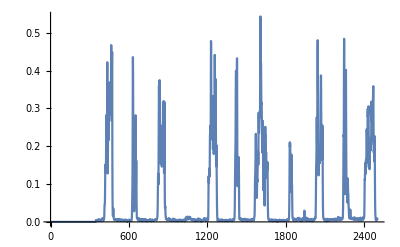

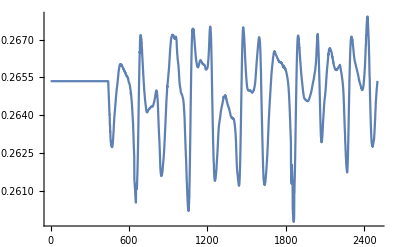

Sub03_(4)sts1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206812.0.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206813.0.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206814.0.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206815.0.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206816.0.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206817.0.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206818.0.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.265206819.0.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068110.0.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068111.0.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068112.0.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068113.0.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068114.0.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068115.0.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068116.0.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068117.0.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068118.0.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068119.0.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068120.0.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068121.0.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068122.0.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068123.0.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068124.0.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068125.0.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068126.0.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068127.0.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068128.0.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068129.0.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068130.0.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068131.0.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068132.0.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068133.0.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068134.0.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068135.0.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068136.0.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068137.0.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068138.0.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068139.0.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068140.0.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068141.0.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068142.0.4100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068143.0.4200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068144.0.4300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068145.0.4400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068146.0.4500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068147.0.4600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068148.0.4700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068149.0.4800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068150.0.4900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068151.0.500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068152.0.5100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068153.0.5200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068154.0.5300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068155.0.5400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068156.0.5500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068157.0.5600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068158.0.5700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068159.0.5800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068160.0.5900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068161.0.600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068162.0.6100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068163.0.6200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068164.0.6300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068165.0.6400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068166.0.6500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068167.0.6600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068168.0.6700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068169.0.6800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068170.0.6900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068171.0.700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068172.0.7100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068173.0.7200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068174.0.7300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068175.0.7400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068176.0.7500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068177.0.7600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068178.0.7700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068179.0.7800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068180.0.7900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068181.0.800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068182.0.8100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068183.0.8200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068184.0.8300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068185.0.8400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068186.0.8500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068187.0.8600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068188.0.8700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068189.0.8800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068190.0.8900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068191.0.900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068192.0.9100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068193.0.9200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068194.0.9300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068195.0.9400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068196.0.9500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068197.0.9600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068198.0.9700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.2652068199.0.9800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681100.0.9900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681101.1.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681102.1.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681103.1.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681104.1.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681105.1.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681106.1.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681107.1.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681108.1.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681109.1.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681110.1.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681111.1.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681112.1.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681113.1.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681114.1.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681115.1.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681116.1.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681117.1.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681118.1.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681119.1.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681120.1.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681121.1.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681122.1.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681123.1.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681124.1.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681125.1.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681126.1.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681127.1.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681128.1.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681129.1.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681130.1.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681131.1.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681132.1.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681133.1.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681134.1.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681135.1.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681136.1.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681137.1.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681138.1.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681139.1.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681140.1.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681141.1.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681142.1.4100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681143.1.4200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681144.1.4300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681145.1.4400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681146.1.4500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681147.1.4600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681148.1.4700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681149.1.4800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681150.1.4900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681151.1.500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681152.1.5100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681153.1.5200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681154.1.5300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681155.1.5400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681156.1.5500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681157.1.5600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681158.1.5700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681159.1.5800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681160.1.5900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681161.1.600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681162.1.6100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681163.1.6200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681164.1.6300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681165.1.6400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681166.1.6500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681167.1.6600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681168.1.6700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681169.1.6800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681170.1.6900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681171.1.700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681172.1.7100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681173.1.7200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681174.1.7300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681175.1.7400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681176.1.7500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681177.1.7600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681178.1.7700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681179.1.7800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681180.1.7900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681181.1.800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681182.1.8100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681183.1.8200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681184.1.8300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681185.1.8400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681186.1.8500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681187.1.8600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681188.1.8700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681189.1.8800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681190.1.8900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681191.1.900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681192.1.9100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681193.1.9200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681194.1.9300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681195.1.9400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681196.1.9500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681197.1.9600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681198.1.9700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681199.1.9800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681200.1.9900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681201.2.00.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681202.2.0100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681203.2.0200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681204.2.0300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681205.2.0400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681206.2.0500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681207.2.0600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681208.2.0700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.4148304600.4408547900.26520681209.2.0800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0015825792904908840.4408547900.26520681210.2.0900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00178265405493679760.4408547900.26520681211.2.100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00180919232334609760.4408547900.26520681212.2.1100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00182171084422221710.4408547900.26520681213.2.1200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00189690800045793930.4408547900.26520681214.2.1300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00187947935682168040.4408547900.26520681215.2.1400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00179969695755898580.4408547900.26520681216.2.1500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0018531296741780380.4408547900.26520681217.2.1600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0021940106134966230.4408547900.26520681218.2.1700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00275473036918898570.4408547900.26520681219.2.1800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00272581934450565450.4408547900.26520681220.2.1900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0025531946090695390.4408547900.26520681221.2.200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00248316029339634230.4408547900.26520681222.2.2100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0029134684985375530.4408547900.26520681223.2.2200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00321417300677689880.4408547900.26520681224.2.2300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00284362928043523350.4408547900.26520681225.2.2400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00265008045637612570.4408547900.26520681226.2.2500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0032832236525880420.4408547900.26520681227.2.2600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0044320799058963730.4408547900.26520681228.2.2700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0055336757340532790.4408547900.26520681229.2.2800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0061349836238472160.4408547900.26520681230.2.2900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0061206318655689530.4408547900.26520681231.2.300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00545680900328906950.4408547900.26520681232.2.3100.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00502330019943788950.4408547900.26520681233.2.3200.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00503852100602026050.4408547900.26520681234.2.3300.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0059506305868399530.4408547900.26520681235.2.3400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.00704048513457787750.4408547900.26520681236.2.3500.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0082541165080691290.4408547900.26520681237.2.3600.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0101111130034469070.4408547900.26520681238.2.3700.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0129604528407920570.4408547900.26520681239.2.3800.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.016886030995180360.4408547900.26520681240.2.3900.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.019327609534025040.4408547900.26520681241.2.400.2653524500.3686983500.3814834100.2795697500.3300065200.4987496700.3034997200.414830460.0188741420646581920.4408547900.26520681242.2.4100.2653524500.3686983500.381483410.00428504358592910350.2795697500.3300065200.4987496700.3034997200.414830460.0187963088468555280.4408547900.26520681243.2.4200.2653524500.3686983500.381483410.0054587032972219450.2795697500.3300065200.4987496700.3034997200.414830460.018915825346956930.4408547900.26520681244.2.4300.2653524500.3686983500.381483410.008668857709300210.2795697500.3300065200.4987496700.3034997200.414830460.018561440137913620.4408547900.26520681245.2.4400.2653524500.3686983500.381483410.0147573393722575490.2795697500.3300065200.4987496700.3034997200.414830460.0205522042104996150.4408547900.26520681246.2.4500.2653524500.3686983500.381483410.02440692116431430.2795697500.3300065200.4987496700.3034997200.414830460.023398703023196740.4408547900.26520681247.2.4600.2653524500.3686983500.381483410.0375578726243835650.2795697500.3300065200.4987496700.3034997200.414830460.0254841277175206250.4408547900.26520681248.2.4700.2653524500.3686983500.381483410.0489322322487386950.2795697500.3300065200.4987496700.3034997200.414830460.026812104680774380.4408547900.26520681249.2.4800.2653524500.3686983500.381483410.0543009622343811750.2795697500.3300065200.4987496700.3034997200.414830460.0288215912722013250.4408547900.26520681250.2.4900.2653524500.3686983500.381483410.058006701167480380.2795697500.3300065200.4987496700.3034997200.414830460.0313836904912684140.4408547900.26520681251.2.500.2653524500.3686983500.381483410.06345123330590140.2795697500.3300065200.4987496700.3034997200.414830460.0348095563406372250.4408547900.26520681252.2.5100.2653524500.3686983500.381483410.066923598399094360.2795697500.3300065200.4987496700.3034997200.414830460.0381630846942713760.4408547900.26520681253.2.5200.2653524500.3686983500.381483410.074569057221697830.2795697500.3300065200.4987496700.3034997200.414830460.035907165467384860.4408547900.26520681254.2.5300.2653524500.3686983500.381483410.086606148110325920.2795697500.3300065200.4987496700.3034997200.414830460.0275036275805040640.4408547900.26520681255.2.5400.2653524500.3686983500.381483410.088297921344535240.2795697500.3300065200.4987496700.3034997200.414830460.0204356291811458070.4408547900.26520681256.2.5500.2653524500.3686983500.381483410.075450031751366280.2795697500.3300065200.4987496700.3034997200.414830460.0200763475990838670.4408547900.26520681257.2.5600.2653524500.3686983500.381483410.059280781761839710.2795697500.3300065200.4987496700.3034997200.414830460.0239260668392640330.4408547900.26520681258.2.5700.2653524500.3686983500.381483410.05307044017063570.2795697500.3300065200.4987496700.3034997200.414830460.026992711104449110.4408547900.26520681259.2.5800.2653524500.3686983500.381483410.047031557451244890.2795697500.3300065200.4987496700.3034997200.414830460.0278832237137774280.4408547900.26520681260.2.5900.2653524500.3686983500.381483410.038113785656842510.2795697500.3300065200.4987496700.3034997200.414830460.027243685756446770.4408547900.26520681261.2.600.2653524500.3686983500.381483410.036326508001433230.2795697500.3300065200.4987496700.3034997200.414830460.0272380092550485070.4408547900.26520681262.2.6100.2653524500.3686983500.381483410.0479546593245473160.2795697500.3300065200.4987496700.3034997200.414830460.027886205325567150.4408547900.26520681263.2.6200.2653524500.3686983500.381483410.060701498894974920.2795697500.3300065200.4987496700.3034997200.414830460.0273000075153309250.4408547900.26520681264.2.6300.2653524500.3686983500.381483410.0611580554334384550.2795697500.3300065200.4987496700.3034997200.414830460.0250486306522787580.4408547900.26520681265.2.6400.2653524500.3686983500.381483410.049507724183925310.2795697500.3300065200.4987496700.3034997200.414830460.0242839682718799970.4408547900.26520681266.2.6500.2653524500.3686983500.381483410.039279315878324350.2795697500.3300065200.4987496700.3034997200.414830460.0276932275267306950.4408547900.26520681267.2.6600.2653524500.3686983500.381483410.032092420890838640.2795697500.3300065200.4987496700.3034997200.414830460.033437452361513290.4408547900.26520681268.2.6700.2653524500.3686983500.381483410.0228807314476071260.2795697500.3300065200.4987496700.3034997200.414830460.035246999765365540.4408547900.26520681269.2.6800.2653524500.3686983500.381483410.0154221096273521960.2795697500.3300065200.4987496700.3034997200.414830460.030817038113450360.4408547900.26520681270.2.6900.2653524500.3686983500.381483410.0174706629867803050.2795697500.3300065200.4987496700.3034997200.414830460.0232493192954357220.4408547900.26520681271.2.700.2653524500.3686983500.381483410.031370616291473220.2795697500.3300065200.4987496700.3034997200.414830460.0193796379468657650.4408547900.26520681272.2.7100.2653524500.3686983500.381483410.044524370393798220.2795697500.3300065200.4987496700.3034997200.414830460.021256716742114930.4408547900.26520681273.2.7200.2653524500.3686983500.381483410.043677078273037220.2795697500.3300065200.4987496700.3034997200.414830460.025987465335667260.4408547900.26520681274.2.7300.2653524500.3686983500.381483410.033653746576525060.2795697500.3300065200.4987496700.3034997200.414830460.0292400306426998030.4408547900.26520681275.2.7400.2653524500.3686983500.381483410.0262121477653416080.2795697500.3300065200.4987496700.3034997200.414830460.0283425510080418660.4408547900.26520681276.2.7500.2653524500.3686983500.381483410.0225228182172750520.2795697500.3300065200.4987496700.3034997200.414830460.0243852204374822720.4408547900.26520681277.2.7600.2653524500.3686983500.381483410.0234615117962368130.2795697500.3300065200.4987496700.3034997200.414830460.0199133710881490.4408547900.26520681278.2.7700.2653524500.3686983500.381483410.0261153022272415280.2795697500.3300065200.4987496700.3034997200.414830460.017570186491154010.4408547900.26520681279.2.7800.2653524500.3686983500.381483410.0244749901423239220.2795697500.3300065200.4987496700.3034997200.414830460.0177761173428024820.4408547900.26520681280.2.7900.2653524500.3686983500.381483410.0207048805175617140.2795697500.3300065200.4987496700.3034997200.414830460.017794595278350150.4408547900.26520681281.2.800.2653524500.3686983500.381483410.020176034831561240.2795697500.3300065200.4987496700.3034997200.414830460.018633681194531480.4408547900.26520681282.2.8100.2653524500.3686983500.381483410.0172418230119619240.2795697500.3300065200.4987496700.3034997200.414830460.0226487031254611230.4408547900.26520681283.2.8200.2653524500.3686983500.381483410.0193376821355352340.2795697500.3300065200.4987496700.3034997200.414830460.023969067000164540.4408547900.26520681284.2.8300.2653524500.3686983500.381483410.031891158139198740.2795697500.3300065200.4987496700.3034997200.414830460.021375653985734120.4408547900.26520681285.2.8400.2653524500.3686983500.381483410.0436174198857915770.2795697500.3300065200.4987496700.3034997200.414830460.0193645834175291930.4408547900.26520681286.2.8500.2653524500.3686983500.381483410.0455753318876185660.2795697500.3300065200.4987496700.3034997200.414830460.0170239674126261250.4408547900.26520681287.2.8600.2653524500.3686983500.381483410.040904235621896650.2795697500.3300065200.4987496700.3034997200.414830460.0146545691998427670.4408547900.26520681288.2.8700.2653524500.3686983500.381483410.041682499899765770.2795697500.3300065200.4987496700.3034997200.414830460.0141980365792707740.4408547900.26520681289.2.8800.2653524500.3686983500.381483410.0471363519325257440.2795697500.3300065200.4987496700.3034997200.414830460.017351063125088970.4408547900.26520681290.2.8900.2653524500.3686983500.381483410.046397613276420230.2795697500.3300065200.4987496700.3034997200.414830460.0229057947404373850.4408547900.26520681291.2.900.2653524500.3686983500.381483410.040247661825567050.2795697500.3300065200.4987496700.3034997200.414830460.028015590961492770.4408547900.26520681292.2.9100.2653524500.3686983500.381483410.033046613663393430.2795697500.3300065200.4987496700.3034997200.414830460.0306438383114280880.4408547900.26520681293.2.9200.2653524500.3686983500.381483410.025851750454343240.2795697500.3300065200.4987496700.3034997200.414830460.0294210274036349960.4408547900.26520681294.2.9300.2653524500.3686983500.381483410.0290815305635505820.2795697500.3300065200.4987496700.3034997200.414830460.0276226408671539220.4408547900.26520681295.2.9400.2653524500.3686983500.381483410.044146603454595030.2795697500.3300065200.4987496700.3034997200.414830460.031622743005081580.4408547900.26520681296.2.9500.2653524500.3686983500.381483410.048238813088297380.2795697500.3300065200.4987496700.3034997200.414830460.041175249151542080.4408547900.26520681297.2.9600.2653524500.3686983500.381483410.043309953060855720.2795697500.3300065200.4987496700.3034997200.414830460.043941531596003230.4408547900.26520681298.2.9700.2653524500.3686983500.381483410.054018791472125170.2795697500.3300065200.4987496700.3034997200.414830460.033753783278634180.4408547900.26520681299.2.9800.2653524500.3686983500.381483410.071569322538050760.2795697500.3300065200.4987496700.3034997200.414830460.02218960917177170.4408547900.26520681300.2.9900.2653524500.3686983500.381483410.069596736936588830.2795697500.3300065200.4987496700.3034997200.414830460.0179440952494181150.4408547900.26520681301.3.00.2653524500.3686983500.381483410.050276589002913280.2795697500.3300065200.4987496700.3034997200.414830460.0156326874776188670.4408547900.26520681302.3.0100.2653524500.3686983500.381483410.0337260456234477060.2795697500.3300065200.4987496700.3034997200.414830460.016526863898185080.4408547900.26520681303.3.0200.2653524500.3686983500.381483410.0297124123349510150.2795697500.3300065200.4987496700.3034997200.414830460.0244066831318339520.4408547900.26520681304.3.0300.2653524500.3686983500.381483410.0281367715843104830.2795697500.3300065200.4987496700.3034997200.414830460.035260129593709030.4408547900.26520681305.3.0400.2653524500.3686983500.381483410.0232594599671251960.2795697500.3300065200.4987496700.3034997200.414830460.043770437169037290.4408547900.26520681306.3.0500.2653524500.3686983500.381483410.019579758032117560.2795697500.3300065200.4987496700.3034997200.414830460.044567260584146470.4408547900.26520681307.3.0600.2653524500.3686983500.381483410.0228677439559273470.2795697500.3300065200.4987496700.3034997200.414830460.034743568085557150.4408547900.26520681308.3.0700.2653524500.3686983500.381483410.033450585496645280.2795697500.3300065200.4987496700.3034997200.414830460.026523715900206810.4408547900.26520681309.3.0800.2653524500.3686983500.381483410.0441694949317194550.2795697500.3300065200.4987496700.3034997200.414830460.0268560665944409250.4408547900.26520681310.3.0900.2653524500.3686983500.381483410.047402916957107840.2795697500.3300065200.4987496700.3034997200.414830460.0276978864616134540.4408547900.26520681311.3.100.2653524500.3686983500.381483410.040634770004400190.2795697500.3300065200.4987496700.3034997200.414830460.0268471394220117860.4408547900.26520681312.3.1100.2653524500.3686983500.381483410.0277694800741474340.2795697500.3300065200.4987496700.3034997200.414830460.0246169866917157340.4408547900.26520681313.3.1200.2653524500.3686983500.381483410.0172003159031593920.2795697500.3300065200.4987496700.3034997200.414830460.0215721949910585120.4408547900.26520681314.3.1300.2653524500.3686983500.381483410.01797944158549880.2795697500.3300065200.4987496700.3034997200.414830460.0225075745123126220.4408547900.26520681315.3.1400.2653524500.3686983500.381483410.0238728565383545050.2795697500.3300065200.4987496700.3034997200.414830460.0248695668910960750.4408547900.26520681316.3.1500.2653524500.3686983500.381483410.032420078701535520.2795697500.3300065200.4987496700.3034997200.414830460.025688721135262980.4408547900.26520681317.3.1600.2653524500.3686983500.381483410.0351986267000217940.2795697500.3300065200.4987496700.3034997200.414830460.0261213139019813160.4408547900.26520681318.3.1700.2653524500.3686983500.381483410.0300375635191361640.2795697500.3300065200.4987496700.3034997200.414830460.0248954134229453820.4408547900.26520681319.3.1800.2653524500.3686983500.381483410.0349197146986454450.2795697500.3300065200.4987496700.3034997200.414830460.0227666432964861170.4408547900.26520681320.3.1900.2653524500.3686983500.381483410.0375554320864446840.2795697500.3300065200.4987496700.3034997200.414830460.0226905465732982340.4408547900.26520681321.3.200.2653524500.3686983500.381483410.0255713452854547660.2795697500.3300065200.4987496700.3034997200.414830460.0229155785785150160.4408547900.26520681322.3.2100.2653524500.3686983500.381483410.0110389737297279520.2795697500.3300065200.4987496700.3034997200.414830460.0234109325911165050.4408547900.26520681323.3.2200.2653524500.3686983500.381483410.0063527336930441170.2795697500.3300065200.4987496700.3034997200.414830460.023165354361288660.4408547900.26520681324.3.2300.2653524500.3686983500.381483410.0123148965334334850.2795697500.3300065200.4987496700.3034997200.414830460.0168320001053395040.4408547900.26520681325.3.2400.2653524500.3686983500.381483410.0205094511476017270.2795697500.3300065200.4987496700.3034997200.414830460.0098992525419356880.4408547900.26520681326.3.2500.2653524500.3686983500.381483410.0200141415988225250.2795697500.3300065200.4987496700.3034997200.414830460.0086973266000227490.4408547900.26520681327.3.2600.2653524500.3686983500.381483410.0142912645775738040.2795697500.3300065200.4987496700.3034997200.414830460.0114769804726724420.4408547900.26520681328.3.2700.2653524500.3686983500.381483410.0117374780992414530.2795697500.3300065200.4987496700.3034997200.414830460.0156708581158480980.4408547900.26520681329.3.2800.2653524500.3686983500.381483410.0157172204780669340.2795697500.3300065200.4987496700.3034997200.414830460.017593097456394820.4408547900.26520681330.3.2900.2653524500.3686983500.381483410.024002153198531860.2795697500.3300065200.4987496700.3034997200.414830460.0147535508170763590.4408547900.26520681331.3.300.2653524500.3686983500.381483410.0276797267217837770.2795697500.3300065200.4987496700.3034997200.414830460.010772892681317550.4408547900.26520681332.3.3100.2653524500.3686983500.381483410.040907599865904020.2795697500.3300065200.4987496700.3034997200.414830460.0099380443005305170.4408547900.26520681333.3.3200.2653524500.3686983500.381483410.0599895903822140060.2795697500.3300065200.4987496700.3034997200.414830460.0107170334465056040.4408547900.26520681334.3.3300.2653524500.3686983500.381483410.058772645866156810.2795697500.3300065200.4987496700.3034997200.414830460.0094408444157434090.4408547900.26520681335.3.3400.2653524500.3686983500.381483410.039396424850540820.2795697500.3300065200.4987496700.3034997200.414830460.009017827205745110.4408547900.26520681336.3.3500.2653524500.3686983500.381483410.023080619204815490.2795697500.3300065200.4987496700.3034997200.414830460.0123467150791366980.4408547900.26520681337.3.3600.2653524500.3686983500.381483410.013194121019022960.2795697500.3300065200.4987496700.3034997200.414830460.0164285834248563480.4408547900.26520681338.3.3700.2653524500.3686983500.381483410.0093257274072963280.2795697500.3300065200.4987496700.3034997200.414830460.014300382934001890.4408547900.26520681339.3.3800.2653524500.3686983500.381483410.0096019806552822880.2795697500.3300065200.4987496700.3034997200.414830460.0101822334855159870.4408547900.26520681340.3.3900.2653524500.3686983500.381483410.0098602974370209510.2795697500.3300065200.4987496700.3034997200.414830460.0109111027915537240.4408547900.26520681341.3.400.2653524500.3686983500.381483410.011011222343019370.2795697500.3300065200.4987496700.3034997200.414830460.012611422016053190.4408547900.26520681342.3.4100.2653524500.3686983500.381483410.016740103541614810.2795697500.3300065200.4987496700.3034997200.414830460.0142429063579875730.4408547900.26520681343.3.4200.2653524500.3686983500.381483410.0191068156043722080.2795697500.3300065200.4987496700.3034997200.414830460.0171553672873428870.4408547900.26520681344.3.4300.2653524500.3686983500.381483410.0134987960996634550.2795697500.3300065200.4987496700.3034997200.414830460.0201786902634197160.4408547900.26520681345.3.4400.2653524500.3686983500.381483410.0091400318881048570.2795697500.3300065200.4987496700.3034997200.414830460.0229186095622135740.4408547900.26520681346.3.450.00209257768291723530.2653524500.3686983500.381483410.010210347230141350.2795697500.3300065200.4987496700.3034997200.414830460.026043812841768030.4408547900.26520681347.3.460.00371149137894075630.2653524500.3686983500.381483410.017616698835849980.2795697500.3300065200.4987496700.3034997200.414830460.0262693490744813840.4408547900.26520681348.3.470.0045916149968047660.2653524500.3686983500.381483410.0247550218733463970.2795697500.3300065200.4987496700.3034997200.414830460.022473456592335310.4408547900.26520681349.3.480.00408179951231440840.2653524500.3686983500.381483410.0237391364437856240.2795697500.3300065200.4987496700.3034997200.414830460.0163749950347939070.4408547900.26520681350.3.490.0033948551929535470.2653524500.3686983500.381483410.0206689984808043660.2795697500.3300065200.498749670.00096787404369725590.3034997200.414830460.0121749757543985670.4408547900.26520681351.3.50.0034073481625237030.2653524500.3686983500.381483410.0264618627277366860.2795697500.3300065200.498749670.0020571830861405910.3034997200.414830460.0117028893623579540.4408547900.26520681352.3.510.0044719028444772450.2653524500.3686983500.381483410.028228026624637780.2795697500.3300065200.498749670.00172978393245806380.3034997200.414830460.0133723827134221030.4408547900.26520681353.3.520.0049205774549627340.2653524500.3686983500.381483410.024126726034990880.2795697500.3300065200.498749670.0011214769623257290.3034997200.414830460.0157888642344052520.4408547900.26520681354.3.530.0042212280145558130.2653524500.3686983500.381483410.0199726455930302920.2795697500.3300065200.498749670.00065893268037725430.3034997200.414830460.0162801183899296020.4408547900.26520681355.3.540.0042322620059563710.2653524500.3686983500.381483410.0135761613984200140.2795697500.3300065200.498749670.00081037265376065580.3034997200.414830460.0199751885467279730.4408547900.26520681356.3.550.0045144900062397840.2653524500.3686983500.381483410.01585491965024810.2795697500.3300065200.498749670.0014264951912771440.3034997200.414830460.0265303632788171230.4408547900.26520681357.3.560.0044332544205093840.2653524500.3686983500.381483410.022846455523464580.2795697500.3300065200.498749670.0032371669758086090.3034997200.414830460.0271037231106681830.4408547900.26520681358.3.570.00368985932711389560.2653524500.3686983500.381483410.0222029069166339440.2795697500.3300065200.498749670.0062349603092557560.3034997200.414830460.019756267634681310.4408547900.26520681359.3.580.00342534650538764240.2653524500.3686983500.381483410.0157492019579532840.2795697500.3300065200.498749670.0088611730576723180.3034997200.414830460.0108203690597453650.4408547900.26520681360.3.590.0044292666430973610.2653524500.3686983500.381483410.0110279606647839380.2795697500.3300065200.498749670.0100768430648196570.3034997200.414830460.0068829802124400160.4408547900.26520681361.3.60.0055814853218378310.265352450.00228549712376142040.3686983500.381483410.0107836672527635030.2795697500.3300065200.498749670.0089830871326677160.3034997200.414830460.0075367565704664040.4408547900.26520681362.3.610.0052757418345694450.265352450.0032322414966492330.3686983500.381483410.0122000537378412750.2795697500.3300065200.498749670.00688872953277606250.3034997200.414830460.0088955902327687610.4408547900.26520681363.3.620.0042743467104704470.265352450.00344905261691852770.3686983500.381483410.016496748334798150.2795697500.3300065200.498749670.0052349134374588470.3034997200.414830460.0112016295868101090.4408547900.26520681364.3.630.0041893337464499450.265352450.0052758769637370060.3686983500.381483410.0276122402863965240.2795697500.3300065200.498749670.004453065714180030.3034997200.414830460.0163908160272614560.4408547900.26520681365.3.640.0048354741651605560.265352450.0062873199526017570.3686983500.381483410.0304957531728060370.2795697500.3300065200.498749670.0048216534602059710.3034997200.414830460.0221026460446201340.4408547900.26520681366.3.650.004361076611739750.265352450.0069457604356387480.3686983500.381483410.025328783512269230.2795697500.3300065200.498749670.0050504532863767610.3034997200.414830460.021409442846017990.4408547900.26520681367.3.660.0039654187454825370.265352450.0100806267530736770.3686983500.381483410.027310676811309470.2795697500.3300065200.498749670.00521815052913646250.3034997200.414830460.0172411115696129260.4408547900.26520681368.3.670.0055178159843352170.265352450.0113205042380535770.3686983500.381483410.0285523911021319280.2795697500.3300065200.498749670.0053858649163238550.3034997200.414830460.0149382855354689980.4408547900.26520681369.3.680.0071219853766998980.265352450.0085070491489024710.3686983500.381483410.0184693340884192060.2795697500.3300065200.498749670.0056466302786533430.3034997200.414830460.012329112928011130.4408547900.26520681370.3.690.00729664927207232350.265352450.0058753751551725280.3686983500.381483410.0097092276567196760.2795697500.3300065200.498749670.0045508053062296570.3034997200.414830460.0110304585619560130.4408547900.26520681371.3.70.0071457325662078210.265352450.0057851033447035720.3686983500.381483410.0120207462065196370.2795697500.3300065200.498749670.00279184736083587640.3034997200.414830460.0120290831539812850.4408547900.26520681372.3.710.005415774714554930.265352450.0078355736203515360.3686983500.381483410.0166376407021581840.2795697500.3300065200.498749670.0030337287344262320.3034997200.414830460.0137690459723826750.4408547900.26520681373.3.720.0047951541966907040.265352450.0067271822586242150.3686983500.381483410.0165337939425465740.2795697500.3300065200.498749670.0044942712970523760.3034997200.414830460.0132325989364511210.4408547900.26520681374.3.730.00387677102710749960.265352450.0041733792595813380.3686983500.381483410.0127680851679355030.2795697500.3300065200.498749670.0049260678839020820.3034997200.414830460.0102837338984728250.4408547900.26520681375.3.740.00246292503872038530.265352450.0024569665821256050.3686983500.381483410.0120422887908606060.2795697500.3300065200.498749670.00474101790592440.3034997200.414830460.0090975848129092650.4408547900.26520681376.3.750.00274276406286392150.265352450.0013590703551025940.3686983500.381483410.0119203474766690250.2795697500.3300065200.498749670.0055666720496301450.3034997200.414830460.0084409937145917560.4408547900.26520681377.3.760.0028322951474035110.265352450.00085437176644989390.3686983500.381483410.0134136046577312180.2795697500.3300065200.498749670.005622049812569280.3034997200.414830460.00591356842907131250.4408547900.26520681378.3.770.0024665169653563540.265352450.00336978382983097550.3686983500.381483410.017712651811469740.2795697500.3300065200.498749670.0044745998782283990.3034997200.414830460.0047172176356541020.4408547900.26520681379.3.780.0026022714890299170.265352450.008331930794173340.3686983500.381483410.0194466237591014760.2795697500.3300065200.498749670.0033744893630425990.3034997200.414830460.00610696588489760550.4408547900.26520681380.3.790.00286316604589473450.265352450.0105132036924891460.3686983500.381483410.021147258325400350.2795697500.3300065200.498749670.00279878786336129960.3034997200.414830460.0085266793623381880.4408547900.26520681381.3.80.00290950258858729350.265352450.0070178344976228650.3686983500.381483410.0179064379580640520.2795697500.3300065200.498749670.00283020446379128340.3034997200.414830460.0125295389517689270.4408547900.26520681382.3.810.00363412979544038960.265352450.0028130560273425330.3686983500.381483410.0099657152605138150.2795697500.3300065200.498749670.00271878004712457770.3034997200.414830460.015344861122574310.4408547900.26520681383.3.820.00321214673546050.265352450.00148555709361224320.3686983500.381483410.0048898003978171230.2795697500.3300065200.498749670.00185662790971238070.3034997200.414830460.0153990352241258430.4408547900.26520681384.3.830.0024804620506273780.265352450.00155220177911197550.3686983500.381483410.00413386019947380.2795697500.3300065200.498749670.00149818208123844070.3034997200.414830460.0178990719602739880.4408547900.26520681385.3.840.00321905566137168630.265352450.00171994130943999970.3686983500.381483410.0048761966629143610.2795697500.3300065200.498749670.00205271537165404750.3034997200.414830460.0239490202620577280.4408547900.26520681386.3.850.0040168331061538010.265352450.00236432418993368480.368698350.00171287171252592250.381483410.0048829222588911390.2795697500.330006520.000442094408051410560.498749670.0026325765050731920.3034997200.414830460.0254305952928419350.4408547900.26520681387.3.860.0046414220035537170.265352450.00302168363209220180.368698350.0029330797417652430.381483410.00723713640077200140.2795697500.330006520.00053483483903299990.498749670.00264615187170578550.3034997200.414830460.0185183131791457240.4408547900.26520681388.3.870.0063274209289624990.265352450.00268435934790945160.368698350.0044464934020997170.381483410.0175783069940963940.2795697500.330006520.00057601820315791470.498749670.0028690518589843110.3034997200.414830460.0109956388702241030.4408547900.26520681389.3.880.0075485752525110640.265352450.00342400810314678760.368698350.0061073519869683710.381483410.0304419194470213170.2795697500.330006520.00090031766417017850.498749670.00186648827170479570.3034997200.414830460.0069329698070750590.4408547900.26520681390.3.890.00704404130302134850.265352450.0063178538796638150.368698350.0061142154591783790.381483410.0309397089608423150.2795697500.330006520.00147457038066338660.498749670.000321695681152301650.3034997200.414830460.0075655314289839960.4408547900.26520681391.3.90.0058003524501952540.265352450.0078691283272391880.368698350.0047927713616676070.381483410.021433078516290380.2795697500.330006520.001996799635324040.498749670.00019349822778350610.3034997200.414830460.0107179246409820020.4408547900.26520681392.3.910.0049231667564726610.265352450.0066509647330316980.368698350.00382305396726020060.381483410.015898981971130670.2795697500.330006520.00282445832933557330.498749670.00191581266980067070.3034997200.414830460.0128742891341025420.4408547900.26520681393.3.920.0059607383539115790.265352450.0062618687105781190.368698350.00317119043828629350.381483410.0128452712066253370.2795697500.330006520.00245725581001570060.498749670.00358102444900202860.3034997200.414830460.0111892415199206040.4408547900.26520681394.3.930.0066329262667982780.265352450.006930471824385490.368698350.0034510184600360140.381483410.0168254726819796930.2795697500.330006520.00142079805576109090.498749670.00355253915975287840.3034997200.414830460.0076733086124560820.4408547900.26520681395.3.940.0058982030898076950.265352450.0070022089720281370.368698350.00385649039091805850.381483410.023636164490317570.2795697500.330006520.00128449334952408660.498749670.00264582019913792330.3034997200.414830460.0062674927023227530.4408547900.26520681396.3.950.0078375698786828390.265352450.0077406018556040330.368698350.0057691210489320360.381483410.021413947222848990.2795697500.330006520.0014443543608808080.498749670.0027236011858475490.3034997200.414830460.0067036162905287780.4408547900.26520681397.3.960.0098057209787946070.265352450.0095306500624139230.368698350.0081788432649918760.381483410.018540709897022850.2795697500.330006520.00143088597687049550.498749670.00381210249514385550.3034997200.414830460.00617775975783935350.4408547900.26520681398.3.970.0079268308480353110.265352450.011605783830255640.368698350.0091185416903702530.381483410.0197539129188095060.2795697500.330006520.00125842620645457260.498749670.0037569693935559230.3034997200.414830460.0047259508229146470.4408547900.26520681399.3.980.0047138905161257550.265352450.0117502041547720270.368698350.0084229086844155430.381483410.025593596018183010.2795697500.330006520.0010376075873476390.498740670.00327537317862687270.3034997200.414830460.0049760466883908730.4408547900.26520681400.3.990.00279034440905763640.265352450.0102093270548780180.368698350.00726180658505869850.381483410.034242382136089810.2795697500.330006520.00075313523847746950.498737370.00334199893613634480.3034997200.414830460.0084121750151600430.440854790.006183310667326160.26520681401.4.0.00272015009729820830.265352450.0109295071422176730.368698350.0080899719385380630.381483410.0405776790227486760.2795697500.330006520.00052973796641849460.498736490.0038626255019415270.3034997200.414830460.0175360340059596730.440854790.0086506154264610080.26520681402.4.010.00272507940919868670.265352450.014478776992419710.368698350.0097171610099432410.381483410.0401821632044831660.2795697500.330006520.00042223675147645650.498729830.0042581299086172960.3034997200.414830460.0257174234974314080.440854790.0134584912637365110.26520681403.4.020.0051840466592683770.265352450.0204730892599810680.368698350.0107148766712980410.381483410.041382555874807250.2795697500.330006520.000406550914215925550.498722110.0039146406185070450.3034997200.414830460.025194467494001910.440854790.0208444352202337150.26520681404.4.030.0082613025199433820.265352450.0243176629570570280.368698350.012623989518456830.381483410.051481614921380460.2795697500.330006520.00069461090636860930.49870840.00358723852200740730.3034997200.414830460.0195665869761867080.440854790.0277555236032053270.26520681405.4.040.0069790311642921620.265352450.020463609820422460.368698350.0147983122796198790.381483410.0555273305760885450.2795697500.330006520.00105878323710602560.498692770.00342897195766526160.3034997200.414830460.0130047596803681920.440854790.0308369603082078240.26520681406.4.050.00513567743781979950.265352450.014240284232751770.368698350.0157129158358415080.381483410.049358736475419910.2795697500.330006520.00166209544150102250.498668320.00319407497696658950.3034997200.414830460.0075446667304547930.440854790.0291073154294640320.26520681407.4.060.0070827912869417190.265352450.01600275717921360.368698350.0142802087052618430.381483410.0447477093274039340.279569750.00135437375269824710.330006520.0019830563430074340.4986440.00259315366112111050.3034997200.414830460.0045602412211723610.440854790.0240733981628652140.26520681408.4.070.0081531575009336810.265352450.015652891318606690.368698350.0109742620484599050.381483410.0382825100909285130.279569750.0026885031161319960.330006520.00161370271244672210.498601060.0019228259935834490.3034997200.414830460.0030542299330258520.440854790.018276509860353840.26520681409.4.080.0083285234331342360.265352450.0083091814354574410.368698350.0065063090735171640.381483410.0238384462242874420.279569750.0033826633501113120.330006520.0013634173402809330.498545920.00234498966885509680.3034997200.414830460.00215233806704006070.441097720.0145511399506544350.26520681410.4.090.0100471937357282620.265352450.0045698370269012820.368698350.00490484746448008840.381483410.01135129787205260.279569750.00305506449674729970.330006520.0016721847703884130.498476810.0023658367859656790.3034997200.414830460.00180328597781537720.441363630.0140232893387875380.26520681411.4.10.016395859498242820.265352450.004372000047162840.368698350.0045187370752705030.381483410.0071462751565528040.279569750.00250573473490401130.330006520.0017963649772498980.4983920.00225391465573140030.3034997200.414830460.0015807028528309760.44165770.0167791540973662970.26520681412.4.110.0310978527038640660.265352450.0039597110651972640.368698350.00319906813735126470.381483410.0056260780559777920.279569750.0022959853450160810.330006520.0014728216407716440.498291320.00206954604956292780.3034997200.414830460.00136310917644102010.441982030.024548625105722730.26520681413.4.120.044269094863747660.265352450.0040530775663844110.368698350.0025207024462264690.381483410.0046190621285730680.279569750.0029693522525590870.330006520.00112658949652076120.498169210.0022465343867070790.3034997200.414830460.0012776365699991880.442345430.035241551693001250.26520681414.4.130.045373266956765410.265352450.00387742044659011380.368698350.0026171948671467530.381483410.0043245846179307770.279569750.0050327129266085210.330006520.00189442166010917830.498038010.0026735953997218920.3034997200.414830460.00145876222013504140.442733350.045815217592277940.26520681415.4.140.04558319038113080.265352450.00356731890856801970.368698350.0024972520914270670.381483410.0041236963520761920.279569750.0084713483825496990.330006520.00287823089871794840.497881290.00334997232418821670.3034997200.414830460.00149295837271491970.443166480.053118187467856230.26520681416.4.150.0570179802142594460.265352450.0042756383142650440.368698350.00189961540726134950.381483410.00487122607479794760.279569750.0128405201846114520.330006520.00345860799148672540.497696250.0046932315274206540.3034997200.414830460.00115114179236548730.44364260.054447814087994990.26520681417.4.160.08300942585274790.265352450.00615542554138510250.368698350.00183068413455214070.381483410.0073793990057093040.279569750.0164639896935741440.330006520.0044412412330370630.497794660.0054906687081467070.303499720.00342505387995285230.414830460.0010764067804912410.443710810.0497851923900801960.26520681418.4.170.119441462178628650.265352450.00725344705070068550.368698350.00307343900676341950.381483410.0096559962339339870.279569750.0177222904337790180.330006520.0054925288435028070.497189640.0062309509964731350.303499720.0039304859471627250.41597510.00157540981317808720.44476040.0418108994083340730.26520681419.4.180.14735453577012340.265352450.007338016276056260.368698350.0043251111973733110.381483410.010261729344482980.279569750.016956429927953940.330006520.00578164241272040650.496899310.0073078454444218130.303499720.00371306979474799860.416687760.00191544626919801080.4453630.0361408994237759560.26520681420.4.190.151882912216887570.265352450.0070711003443050230.368698350.0048768877432774010.381483410.0101406105061403360.279569750.0148073512522495860.330006520.0049076309771852260.49657530.0077662582473036580.303499720.00386046491482922680.417471840.0019576986000567230.446025250.038828761179916020.26520681421.4.20.14794774141033460.265352450.0075963739818763040.368698350.0052987371414607160.381483410.0105419572347484720.279569750.0129477468323863890.330006520.0045899101916139110.496242250.0096753237867788140.303499720.0054307498162614290.41826740.00223094956335477070.446697450.047867512703782070.26520681422.4.210.13973528062801540.265352450.0078573781995245980.368698350.0055471604736715560.381483410.01081743743877390.279569750.0140284875158986720.330006520.0067804446796010320.495886680.0143742146324975450.303499720.0066521996391655020.41909380.003407449427533510.447397390.056192763214478130.26520681423.4.220.12948420739884090.265352450.0071649623143299790.368698350.00481077765149002640.381483410.0100583192628586180.279569750.0177082196185354150.330006520.0115241497071462310.495496030.0204990302984206580.303499720.00699861729220886950.41995990.00540417540022313650.448138930.059032281408174240.26520681424.4.230.150627368723725670.265352450.0065693501567072490.368698350.00374010587800077550.381483410.0087332999928847170.279569750.0220666964334992580.330006520.0177582553358452720.49507190.023819040969760660.303499720.0078973211763814780.420860350.0067841918131430060.448918070.0559410083375263540.26520681425.4.240.200471800332259170.265352450.0066325071295637770.368698350.00325356898549757950.381483410.00756771625512766850.279569750.026160095109088360.330006520.022032653241352740.494628610.023191307176143090.303499720.0098286544227298140.421773650.00691488277698319550.449712940.04925438151678210.26520681426.4.250.254151214431305450.265352450.0059363965041117340.368698350.00291250307537314770.381483410.007483007152851510.279569750.0298805722735010460.330006520.0224699487425163680.49414670.0222122356252400340.303499720.012323740866976810.422763060.0074902590544319570.450572830.042902829855312950.26520681427.4.260.282690551998177550.265352450.00535870203329306350.368698350.00318243667466251360.381483410.0085955130940196970.279569750.03250674332360080.330006520.0215770443038464830.493654210.021421971160317180.303499720.0159777442794336450.423757980.0081449591839017760.451439610.04216969394267250.26520681428.4.270.255840525019456530.265352450.00566730262523612760.368698350.00404628688276643250.381483410.0096789627663262690.279569750.0324860003882892140.330006520.0202070570203866720.493137460.0226726828268343820.303499720.0224199052684261950.424793490.0083568745890164170.452341360.0487727713995865860.26520681429.4.280.197942930953039830.265352450.0060080254214156610.368698350.004544682473018680.381483410.0103061791549526450.279569750.031598457522192830.330006520.0186788667976888240.492612620.026926428116670870.303499720.024988150843366070.425842450.0091381407739776540.453249690.0583465128462476240.26520681430.4.290.165519549085818370.265352450.0056566586780474590.368698350.0047040748246942530.381483410.0104495977508822710.279569750.033472926043593690.330006520.019109997465717180.492077440.0320401015682765240.303499720.0217034651949304070.426897970.0091190117202803250.454160230.065671382233182350.26520681431.4.30.180677380975090170.265352450.0047278859087286440.368698350.0056513739831499010.381483410.0106335852365756710.279569750.038557353719800560.330006520.0211652911027383030.491529680.0388826535096183650.303499720.0217133740608207830.42794970.0072400811113026120.455066370.06690615983902680.26520681432.4.310.264754578648624670.265352450.0053369385408011110.368698350.0073515381536309040.381483410.011384770295209740.279569750.044833122908769550.330006520.022667116495926470.490966380.048865267924620520.303499720.0277393937078307260.428997080.00582710269511135460.4559680.061700645435990890.26520681433.4.320.381307514635334970.265352450.0068222605185427110.368698350.0080257222700980420.381483410.0128689139638380350.279569750.050606689679283150.330006520.023462115185919010.490379080.058419874011312650.303499720.032340065454400510.430053140.0054659583835855720.456877820.0526911463804139240.26640703434.4.330.422230268901814250.265352450.0088375090515456780.368698350.0082153551346737470.381483410.0169256499842444160.279569750.057673119986760480.330006520.0247563795583010570.489779750.061985684107821720.303499720.0282371430964764930.431089340.0062466763686614810.457772390.043580666387183080.26760932435.4.340.34730325624276770.265352450.0098686425412517420.368698350.0091401476426534770.381483410.0245611747220214930.279569750.069094744366529960.330006520.027313034596080520.489148130.058570309671992110.303499720.0212759608737025960.432148430.0081197343247637560.458689330.0382928748635710660.26884887436.4.350.225473951964195530.265352450.008857953043775350.368698350.0102196035207394540.381483410.034273067771345380.279569750.086415625888844220.330006520.0309418217271763970.488529640.051782687881057940.303499720.0176883868044535740.433158240.010890994702173960.459558720.0391773139788937560.27007441437.4.360.137562604475799650.265352450.0071988760539685870.368698350.009812559441927090.381483410.040062065633961410.279569750.104783229341808090.330006520.033242728807020420.487910920.044783298277180490.303499720.0168187533837969960.434160020.0127546182282328410.460415020.045993451907078520.27130858438.4.370.128209237922226220.265352450.0075082652412111080.368698350.0085372614778502910.381483410.0406989065925963050.279569750.114431304045190990.330006520.0333764181102326750.48728170.039027751344510320.303499720.0160075326708011630.435159640.0113528294291350830.461269370.057200219809971080.27254769439.4.380.18632205907127460.265352450.0081642755759099680.368698350.0078714938455066870.381483410.032311577386514450.279569750.112012288644377650.330006520.031660800229430210.486722450.035801440140181090.303499720.0121936327035473360.436066350.0091887175778069540.462023960.069242349745959790.27371201440.4.390.24166694969795280.265352450.0078940091967091880.368698350.0073079495984736320.381483410.023209869918888860.279569750.106193276246452180.330006520.0297804570941974170.486151560.0357530090007349350.303499720.00712213605608662350.43698740.008942731295875450.462789620.078286151724075330.27488298441.4.40.25479701469277310.265352450.0084156202054143020.368698350.0069275508084625980.381483410.0210565761952977540.279569750.105808873305982170.330006520.029598955415278760.485609550.034922915100421540.303499720.00456849592116964540.437872980.0109798723238257390.463514860.083188983811755780.2760187442.4.410.252991931779048830.265218330.0074973757550097550.368698350.0062636689751449570.381483410.0187154393694612430.279702520.110740541729859840.330006520.030000936682981830.485107470.0312257288066241960.303499720.0048759808374393090.438711440.0135882777475538480.464187550.085313557476934020.2771067443.4.420.250003734726626960.265090330.0049235751224354310.368698350.0050997511515423080.381483410.0118902724627047720.279828980.117049449454932770.330006520.02994013682734010.48460550.0279108307302506250.303499720.00594788871846589460.439543170.0157677525860431370.464857520.088214310693135620.27816662444.4.430.229238623700009970.264969410.0044495046954268480.368698350.0042333217995750640.381483410.0058602054831420980.279948210.119198322214391330.330006520.029413067196698110.484140110.0263965565042830720.303499720.0070861328252605430.440324210.016219023966379690.465478480.096792422445033970.27916842445.4.440.216579507839706170.264828430.0070437357181795760.368698350.0039011458377412380.381483410.0052594113202985560.280086950.111865199220075320.330006520.0284188884440588830.483711320.0298148323667288450.303499720.0077011586643168510.441052240.0140915572711578320.46605010.113165355604609790.28010814446.4.450.246633735987542240.264693730.0100996897898676650.368698350.00379639089674227960.381483410.0077805504123059950.280219220.09500200320260270.330006520.032428357995118140.483306570.038054060807074090.303499720.0057376725614923660.441741130.0125068214530728690.466587270.132934501725216430.28099937447.4.460.2808057460058380.264557510.0106997209852003560.368698350.00347613146690301050.381483410.0095057793288407940.280352710.076876666685529090.330006520.040788947781928880.482932170.042200598370361080.303499720.00218955986870577640.442381970.0136004366767797530.467081790.148371237643802470.28183109448.4.470.28348193644005460.264423930.010036888606867150.368698350.00386383215247974950.381483410.0099561156610940630.280483330.07045045080764570.330006520.045689109099558880.482593410.0421123921905607050.303499720.00175597438346512620.442972850.014375445189096710.467527480.154199560535220240.28260989449.4.480.28934416705818630.264283260.0097919125813136220.368698350.00437381209207793850.381483410.0104686662507229270.28062060.082321459037544810.330006520.048192582318106310.482298530.046593130482171490.303499720.0055238079049697180.443502510.0124709698523988740.467912780.148637046303478930.28332728450.4.490.31258022073096750.264148380.0110185048466800130.368698350.0039754106834008680.381483410.0116271989641109110.280751930.105465183370786070.330006520.052823238372229160.482048520.061369060718418080.303499720.0104351821096221790.443969190.009720217217491350.468236160.134085800713939720.28398009451.4.50.35571942005406730.26401640.012470987321238560.368698350.00231296932656106230.381483410.0125562725789612250.280880180.12741535115559770.330006520.058030522165974560.481836230.079517938236871990.303499720.0146594214883339880.444373630.0083452838856268810.468502260.117142091017461050.28456962452.4.510.369005382645787860.264017860.011985021480673290.368698350.00106626029219236830.381483410.0121460025452810890.280878760.141469076303344130.330006520.062927953471833390.481957930.090622165829564190.303499720.0192238522863964550.444417490.0079155296915680210.468353950.105127323677335070.28492805453.4.520.335110977800851750.263745090.010244089017951450.368698350.00171088208513164820.381483410.0101717628226987520.281142970.150063459946813830.330006520.071861243290289740.48152030.094137556870383320.303499720.0236472966164659740.445020110.00774270672795660150.468873170.101826906256057570.28559802454.4.530.302696064797389030.263606420.0085933771861485450.368698350.0035350388535252870.381483410.0083879857663090080.281276870.15697201509342450.330006520.086013705125976530.481413120.096155345987253450.303499720.026379196856191670.445266650.0072437777915850410.468981640.106801108122150210.28604543455.4.540.288234846467633140.26361130.007433836980321830.368698350.0057617642107367590.381483410.0090112118853959020.281272160.15837810046595920.330006520.097966834153697650.481557650.092855641439704120.303499720.0268053088522185730.445239660.0064871600903260580.468775470.116798284002433670.28632318456.4.550.28449973178729290.263353740.0089335253336076950.368698350.006923573748356130.381483410.0113926376939655570.28152010.14650500404319620.330006520.101161920204809670.481282770.081249192897916060.303499720.0246606717578499480.4456220.0060700021235708690.469065340.126668749534535880.28682593457.4.560.293482901158406140.263362070.0120225988322930580.368239690.0060407843534236840.381483410.0127088499163632090.281512090.123897195614143090.330006520.099170960145471650.48141420.06684232969274680.303499720.0205808276459157440.445579170.0058260752033709120.468859080.131876897796913280.28706466458.4.570.324896930812674840.263164520.0142727647006959750.368010310.004411674021327740.381205230.0124497027660026950.281701610.103825786959017720.330006520.095413970508120130.481223370.053117692718135960.303499720.0155619734775419620.445849720.0053598576643038220.469037920.130050159859532830.2874449459.4.580.34523477932866710.263072210.0145936977396174980.367689560.0044749707142696810.380837470.0115180820920376720.281789960.091590441328847960.330006520.084228801726113770.481221350.041533505964496110.303499720.0113885456139327930.445921470.0047422535266068250.468986480.121075417148510220.28769727460.4.590.292080546748402340.262997780.012814937913078530.367371740.0053966512326787730.380473830.0103038580638489720.281861110.080148432259487240.330006520.065524952366529350.481232230.035137530137107760.303499720.0093600094508591180.445969560.0041740133828091980.468917380.106982636822303540.2879129461.4.60.2841757792576360.262942370.0111246729448245780.367056610.0053600806523362550.380114410.0091869268101959860.281914020.065244925642682390.330006520.0502058205381456440.481262950.0372848203293728450.303499720.0094032657430708140.44598980.00399124349238552750.468821770.090326973331251660.28810691462.4.610.330070797259057860.26295610.0105983753796671420.36669380.0049830660317925240.379709840.0094918631686816480.281900920.052178782607313280.33038060.044339131837797060.481387910.046323345205134790.303872270.0102069793961252260.445908250.0043259770600642590.468609380.074566414363550170.28825322463.4.620.41285765599786060.262842670.012341621695055750.366476420.00530358680080592150.37944970.0115278581605471260.282009120.050166464169422020.330732250.0448960993642862840.481415930.05405237321469430.304223170.0109524009896946380.445918480.0048852012221156610.468512470.06456799431462140.28843888464.4.630.46769609610907830.262803650.0122971773341115850.366202430.0056379235912761590.379135480.0121174862417091290.282046290.060214391642150360.331059160.044698241800868240.481549490.05675352572692310.304550020.0118583629237930620.445818170.004814344630201530.468286550.0618962100415192050.28857359465.4.640.432188526219345340.262828240.0086753333850786920.365879060.0060122908749506260.378773880.0097223253352887490.282022860.074027737018667260.331366140.0444355059155282160.481707090.0577194462009181860.304857540.0131245667927690490.445689130.0040059025415410530.468030650.063711515461919110.28869175466.4.650.37972848262330680.262837290.0057647049528260970.365581160.0059616577830193440.378437970.00722357552870377550.282014240.08183129518418910.33165950.046949793869847020.481871660.05740548853293670.305151950.0144694138972480820.445548380.0034126851803640860.467765590.06646906882728930.28879485467.4.660.32810332228912050.262840620.0047439281997481250.365296970.0049040657454602730.378115940.0069631089560799260.282011060.077494048662876390.331941430.049892556287451040.482052060.056482416955837530.305435410.0142968534761194980.445387440.0032546878140533720.467481410.06733886714466590.28887395468.4.670.267280869265759450.26275350.0045838426533543070.365104220.004340991776540460.377883150.0084156667272477380.282094030.066847910502412150.332220510.052292369022436790.48236080.05648931514762590.305716510.011528329291133190.445092210.00317053577973656260.467045070.064970763964239450.2888406469.4.680.279978257913049760.262742970.0059135251124841250.36484520.0044877038000415640.377586090.010579029422321380.282104050.066105656222910940.33248510.056701286524789550.482622650.057313485377390710.30598350.0087548938528002070.444842330.00312344295476844330.466665520.0602559189005388160.28882884470.4.690.41405524410588870.262734490.0069037997170477330.364594230.0039809035707006810.377297820.01203698237309890.282112120.079446997896061060.3327370.0608793385969879360.482912930.056694282879117530.306238140.0082054322124406940.444562220.00310817062676473640.46625490.054280881927277780.28877986471.4.70.44931540477958830.262731730.0060001587208477940.364350910.00378173535268818860.377018570.0117233537188378930.282114750.095614396911049340.332973370.061217600563184250.483228620.051619829939270660.306477480.0095424034327913230.444255010.00264014370761162880.465817490.047232300256473780.28869753472.4.710.31161808624234530.262742420.0036578026057179670.364114660.0042669527906368280.376749050.0088408147417774110.282104570.103848401921095610.333187790.055100294021654650.483556990.041720107642756930.306694950.0094008999579189450.443935130.00189665489560281980.46537070.038961876926867310.28859145473.4.720.14618285387008360.262762580.00228833149653924530.363894310.0044661613228853450.376498890.00544786517059744550.282085390.097366806740980290.333376310.042899680795205530.483906170.030496859858017480.306886430.0075075681066684910.44359460.00156995574764862690.464905930.0297656367954935270.28845958474.4.730.063908950299009850.262794750.00244015534442480280.363696490.00364125527266970140.376276360.0034948608710616840.282054760.076717219330712280.333530920.0293521651086803660.484270240.020717955919143680.307043670.0060783396514797070.443237140.00154122898473025710.464432130.0212660080810404930.28830143475.4.740.035873343525045190.262838450.0027695084248902110.363517280.0029807418635563510.376077020.00329405264286200060.282013140.051158661847827980.333656380.0189556138821346080.484453560.0130255511846670260.30717140.0044664950307276180.443059480.0013079896773898790.464175650.014035564451112560.2882746476.4.750.022103133125002290.262877680.003078837518258960.363391850.00280439772459092340.375938890.0038574864009261860.281975740.0306716539289094460.333735640.0123917047513877710.485064840.0075947556709875040.307252150.00335182031703858430.442451510.00135503033783287050.463432730.0086361780328895990.28790913477.4.760.0157378636782168380.262947950.0035966335735234490.363264230.0028231822893977030.375803570.0045617629731837180.28190870.0179646136388068170.333787530.008999603946124930.485497630.0042758323419342750.307305040.00336446440624609470.442019440.0016574675595110080.462903980.0054779844082599860.28767246478.4.770.0197676253201556840.263024580.0044146660067784650.36315850.0028620416182494210.375694680.00468716289535439650.28183550.0111802427761939250.333813090.009221334752693790.485957050.0032110244880552090.307331110.003616460851479120.441555120.00183834866634594140.462350620.0045912451117279390.28739694479.4.780.030256325248336740.263106440.0052667764325132890.36307250.00308492848358832020.375609530.0045408465934094930.281757210.0082818384243540480.333815490.012690507365118650.486444510.004882492406215420.307333550.0038080792755728610.441056250.00194257732808832760.461769510.0049813579471131520.28708331480.4.790.0351892348233262960.26319870.004700281131120090.362996740.00347751436890707430.375538080.0049089181553568280.281668870.0088002626566562810.333798590.0172549779409026070.486957950.0096599281661742550.307316310.0040095295057185190.440525890.00190391498809864420.46116250.005548124874542070.2867326481.4.80.0292428501880783770.263289570.00323267383460234830.362936520.0043408392728846950.375484380.0077108653668530360.281581710.0116033346963121680.333768530.021295327952450730.487489130.0150122926376550820.307285670.0047761863810013120.439970890.00205555417288244250.460537330.0063056532455576170.28634809482.4.810.0198939565961006870.263334540.0035678826522858780.362930180.0074921401352583130.375484930.0189327126462774560.281538540.0155694097511837030.333731920.0248377079035460270.48803240.01644117087931180.307248350.0052464362695182660.439394670.00219576294745658760.459898220.0064891470591593560.28593184483.4.820.0124853823412683240.263475380.00533374506514588350.362836140.0122983495801551460.375400910.0342489079466165440.281403130.0198178003222304370.333685590.026573846991943240.488592730.0146279126823843380.307201150.0053064812026208460.438800520.0022704964529319830.45924020.0071262329245174770.2855053484.4.830.0093009458884006980.263568090.0063979878482051720.362790280.015647480940296080.375364140.040921437486744890.281313830.022915346902888030.333640040.0253555759719881030.489159870.0140569833589537350.307154740.0056150322487891560.438191680.00219258045558222860.458571660.008022733437332160.28506132485.4.840.0084325743573451080.263665140.0056327886654877610.362737890.0155828302643041370.375320590.036382184585745770.281220210.024799853319347280.333596220.022630800314039860.489728640.016226048536417480.307110130.00610925184089281150.437576480.0017291964561100890.457898010.0070853006680198760.28461663486.4.850.0067052214959220350.263758880.0042138712451885630.362681480.0130783699048771810.375271840.029382572146452220.281129650.026719405166811510.333559130.0193162432708511060.49029720.0194764038058696450.307072380.0063553669897996220.436959130.00149187676859744530.45722080.0054697374977070650.28417689487.4.860.0055787722179409080.263840560.00355413728026417840.362628140.0098387053010687080.375224520.022906559523126420.281050630.0281877477594447740.333530610.0179988953207558780.490862260.0216992186330884660.307043340.005600710200724480.436344670.0015287439559965060.456544160.0045435879422196790.28374557488.4.870.0049755570489730960.263918370.0036772803837174060.362566130.006850815456336880.375166580.015149189062841520.280975260.0292768484601228850.333513770.019391919592946340.491425590.0231601023768698740.307026210.00457469785421922050.435733860.00172986382654510830.455865690.0043943691463323010.28332717489.4.880.0047794388793313210.263986350.00380951318134362770.362504760.0046551649965841620.375107640.009111911157608050.280909340.030749626316577960.333505730.022293046624757750.491981750.0264165272093594560.307018030.0044950513949078270.435132960.00162675190283508650.455192880.0041416660171406790.28292522490.4.890.00541637607432842850.264049140.00430091934226031150.362438860.0036703557958284760.375042610.0093629261781358230.280848380.032356476168122540.333506840.027094434740685120.492531540.0309624512354285950.307019170.0061631999041546420.434542290.00143144829098339130.454525360.00484080848146937240.28253825491.4.90.00614344944311948260.264110560.00541480090940080550.362364710.0033609041896611360.374967820.0122512304361738370.280788710.035379017823854140.333516960.034301335571863690.493070250.035540501780911650.307029460.0078500736311193140.433968690.0015918811461612050.453869370.0075662766842659880.28217183492.4.910.0064531212938136650.264172360.0055820926740835290.362282590.00340449546182241150.374883920.0118734852103199710.28072860.040087418569465140.333534090.0429997498379103350.493594320.0398495330831116840.307046890.0079092592859615270.433413280.00157826421587671760.453229230.0085978081384864850.28182371493.4.920.0061576157130736970.264233610.00357950179141476330.362193610.0045638448067322780.374792030.0126603296516178430.280668970.042599564225374430.333558090.048153916747393980.494103350.041623378276586110.307071310.0075286799432218630.432878050.00150375220275814160.452605990.0074809044686540790.28149551494.4.930.0051794054190787040.264299050.00274180386489056470.362093940.00655892828914575450.374688520.0161823084697986960.28060520.0396570390130719650.333587950.0427792567169705260.494592490.038235479967019790.307101710.0079471769422227240.432365240.0017238884748332910.452004820.0068503827601855130.28118861495.4.940.0051053892563491210.264367350.00363599602868617350.361985330.0068151077369417630.374575220.0211079317001575880.280538580.032458807122939290.333623270.032033139079336510.495064960.0307878824724210.307137670.0084609553823391140.431873080.00188241664090493440.451422590.0067081706514734990.28090154496.4.950.0060039876751331450.26442610.0043776774731369170.361882890.0059265875961498220.374467340.028643241376466850.280481210.0248065981732292320.333661940.0233610594053498930.495519820.0223759748217045550.307177060.0073772608179476950.431399110.00170149255133374250.450860640.0063587708381426530.28062605497.4.960.0057935317662898480.264488910.0039814439325338390.36177320.0062309995498268190.374351810.032362841894296630.280419820.019695459446159690.333703330.0192453630357076670.495955830.0145572537854202280.307219220.0054461331979131730.430946610.00140976860885619490.450320810.0049283196398488960.28036807498.4.970.0054079024744257290.264557210.0039158061977317180.3616560.008817692508310160.374228560.0287688967120527040.2803530.0188278630029542970.333746280.0197442036860067150.496370360.0087338862536846790.307262990.0045857025236686450.43051620.00150953539660893820.449806710.0045143871800715290.28012149499.4.980.0055399511802529290.264621670.0047516808240054740.361541550.012910471762647230.37410780.0264928077564000020.280289870.01997421924672330.333790240.023366717624523030.49677720.0053525272125158930.307307810.00400239144423174350.430094410.00153782877944789570.449301510.005722291426658020.2798819500.4.990.00653391902282030560.264687220.0052189897712877810.361426960.013971247298827630.373987050.0263492899783358170.280225610.0186861540504314370.333833160.0286767359798220860.497181150.0037117019530434520.307351570.00381359125015839040.429673870.00114533532558138230.448799690.0074110441616787130.27963942501.5.0.0074091346727565030.264747220.0042278216643458560.361319610.0101167268905851680.373873680.0209723301598487640.280166720.0145141731037000120.333874590.0384730677056624660.497599880.00293791750102607350.307393830.00364858309867602350.429235170.00098090679759875540.448279340.0092133718247950430.27938303502.5.010.0070954747447300490.264803360.00321131379251438170.361220430.00710576315726640150.373769040.0157975296909774050.280111580.0098144128332088560.333912090.0524753263004511740.498034370.0033414545341022840.307432110.00360657551344592930.428774370.00108787276412233850.447739540.0107681138710299680.27910379503.5.020.0062014509144970960.264869140.003067578908922290.361115180.0074499286884225530.373659130.016944349265590630.280046910.0064655401993981060.333945880.0666711524002220.498494930.00485112185190990.307466590.00306406784553980550.428282930.00116266714273964440.447167370.0119829750211302140.2788041504.5.030.00414227606178362450.264923310.00302493909722921070.36102490.0085061834168125570.373564440.021998007296267090.279993610.00487947975865729140.333976920.076127703224772150.498983960.0059505333288673710.307498290.00236954673798874840.4277560.00105705203474087790.446559580.0123756029163878370.27847501505.5.040.00289819285760424060.26497020.0027226055013870460.360946360.0077676319890734740.373482010.0203332943169911750.279947430.0040452023748792970.33400410.076724058688460810.499508120.0055916219418983780.307526040.00226607620929103640.427186260.00102400354884016740.445908570.0126663755738449760.27810842506.5.050.00337618592436632940.265021120.00322360947631412760.360867790.0056281235312158860.373400290.0121474905021174830.279897250.00348787848860846170.334027410.064761568091323970.500071220.0044385272494442010.307549850.00285935463891459850.426569230.00095941185425130810.445209280.012269541986186350.27770195507.5.060.00351900786080799760.265066180.0040912919691380850.360798970.00360741179349617550.37332880.0063191455335488660.279852810.0034534667891353420.334047350.052640508623668690.500668770.0042310821647836660.307570210.0039246055438309910.425910160.00093713603942042870.444467410.0110503059640497220.27725731508.5.070.0049789051663869260.265111620.004657076759727090.360734130.00276495070935605560.3732620.0053448672947904230.279807960.0032999829444449210.334063250.054347951800768780.501286640.0044442317145349860.307586460.00385926489331115540.425222680.00079433184597361050.443699370.0094631218746163980.27678554509.5.080.0069300277357096380.265144210.0050870027595071440.360682550.0028505151477128560.37320820.0065970027558622530.279775780.0025707011067916890.334079270.061254854819596250.501912450.0046671532389464770.307602830.0036337898851804720.424521430.0007564373709427230.442919050.0073248850554827840.27630266510.5.090.0077553752981212040.265185970.0050945259141316830.360622140.00323370096863707150.373145860.0084132927696279020.279734510.00190661143494283340.334094580.059837374564322150.502518080.0041462666322028080.307618470.00352956095369593580.42383760.0010030860360902040.442162620.00554346995676233650.27582204511.5.10.0066612275867291630.265228030.0048836192600327350.360562280.0035438068732497170.373084210.0109454630900601370.279692920.00176873611685406760.334109070.0491708578632352250.503111410.0039894244847446860.307633290.0044985768727975960.423164720.00150671041659216640.441420550.0051205997504254820.27534398512.5.110.0052750612940061170.265279320.0045597758107468670.36049310.00327610830462387930.373013460.0127605185097324650.279642180.00162113782926745240.334123250.04122066098905720.50369680.0040441757047808760.307647780.0049020345688690540.422498680.00168979970815547770.440687060.0060785241738406430.27486939513.5.120.00496622276748491950.265330140.0038801721183039230.360420760.00428321839212227750.372938970.011361709973690750.279591850.0017010851871257080.33414070.044507524076873450.504241030.0040404973330545880.307665620.00296684491359050640.421879160.00150034578218753710.440004690.0070568852501485590.27442012514.5.130.0039913894350687350.26538430.00321976842867567740.36034720.0075741236332915060.372863680.010995439813413680.279538170.0022656801525115180.334156040.055532330605204360.504741120.0046882292680389530.307681310.00118799718365897640.421312870.00152278770861233180.439379050.009043275060579720.27400422515.5.140.00365637790925224530.265430240.00388873901628482850.360270130.0125305519267486580.37278280.0157824702919605180.279492610.002667226000616330.334182340.068413452080775470.505224040.0065599251083061860.30770820.00147102939551656720.420767820.00180700900733100720.438770050.011934590894899310.27362355516.5.150.0041585163732332990.26548530.0050214317873114620.360187360.0155603364034037210.372696990.023637426380611980.279437960.00297896997685198140.334205090.075588789742150680.505673190.0080665424903027280.307731470.00239091379832469430.420263360.00189330021334793040.438204940.014539760781959750.27326755517.5.160.0044834043871249340.265536980.0063459030540817840.36010410.015248579970485740.372609990.027205665607277580.279386620.0039710518808037140.334231430.072366616892167320.506093140.0065850755505592750.307758420.0032317585768508610.419795580.00165665009057880610.437676510.017111759140315280.27293856518.5.170.00373228278477515840.265578340.0096461282893954970.360030520.0126793403758147650.372532280.020732425125205060.27934550.0050554689849291310.334258760.0600452019239186560.506502080.0040898404219158290.307786390.0042874229004329180.4193410.0012306873418610380.437161290.019094581630212240.27262119519.5.180.0034811146574576030.265650250.0117095889881117520.359928510.0084350272298590810.372427310.0106285542461452620.279273950.0050820428922041970.334282740.046463018915639280.506891090.00329815393927352640.307810920.0057269464412588040.418909740.00125542110204134290.436670170.0203380007721711730.27233009520.5.190.0042572407630947110.265715640.010084553330530180.359832850.0050757818487910620.372328480.0059571808639253510.279208820.0038414000668250120.33430710.0394046268886244640.507265870.0031322320757194230.307835860.0058920419509184890.418497220.00152666729810554240.436196460.020224027407917840.27205967521.5.20.005419146454950930.265755030.0073388183251958790.3597660.0041201688173678480.372258230.0059566216012405970.279169560.0027896508737955270.334330050.04099009369253650.507647070.0029152064903242350.307859360.004994517468098820.418074810.00193215112744726040.43571330.0188131259191398370.27178474522.5.210.0071824126684408220.265791310.0059626962190203490.359704830.0047253151045559770.372193980.0089712122806489820.279133370.0029298479260963820.33435080.047983600349507580.508018170.00307429777226239130.307880610.0040670496734718870.417664970.00217859131522502240.435242830.0167818649220866580.27152229523.5.220.0079250301160271910.265832490.0053129629459209070.359639190.0053560904721596880.372125470.015280075663633960.279092280.00332396590800055440.33437090.0550683874753462450.508373990.0037045839577833260.30790120.0041930487859399640.417272960.0019790907045892560.434791550.0146559717678296630.27127326524.5.230.007486874119630290.265828880.0044506925852292660.359642810.0044964115256239360.3721290.022531082743950320.279095880.00271380766722499350.334371060.058653041063475940.508356690.00368484921445167650.307901360.0049950947184175250.417294140.00173410608404398990.434813180.0132176938864926610.27129323525.5.240.0061923544683817220.265890370.00511617216085463650.359535420.0039203545453319320.372015780.0235803993040952230.279034470.00184959938941923360.334409420.063268539151396530.509078030.0033037454900782880.307940660.0050613919961691830.416496380.00155253157950702120.433897090.012147729246057030.27078468526.5.250.0050749598615064820.26591060.0066953194558906840.359492830.0061509769333455920.371970080.0182624322899843370.279014250.00161077802159958320.334428540.063829745060613050.509427170.00390559427356620670.307960250.0048468536138972830.416109390.001494492873427930.433451930.0121135250190754080.27054443527.5.260.005628579105486380.265931540.0081958342234310440.359447980.0080979475503125170.371921880.014959294738966380.278993320.00233274467745102530.334448990.0564411915019930.509762280.0045532518229758510.307981210.0041300029276981910.415737620.001397752797385330.433023570.012180333847012090.27031623528.5.270.0061563868892016450.265977690.0092741512746629460.359374340.0085384076834878790.3718450.0198392959144515940.278947160.00332470696173156520.33447140.046170522996501660.510065630.0043658286089777940.308004190.00344670634774823460.415403090.00115487909891220650.432636060.0115984946780513350.27010892529.5.280.00658078653080230.265972290.0088507047649443340.359358690.009300660946790.371825730.032930144019756690.278952560.0042796156633069670.334490510.03991773961938960.510396270.00299274697855277670.308023780.0032023139138361570.41503520.00099275312038552220.432212920.0103551167093488460.26988198530.5.290.006372066176624490.265977990.0061704152672424570.359323170.008525046395628040.371785440.0400619843341262350.278946860.00537365591701204240.334516910.0430383240984362550.510678160.00147980439023940950.308050840.0032363257456542640.414725110.00095495129239666750.431851410.0089092120772918270.26969298531.5.30.006335743867502360.266016510.0040214919800220540.359257140.006927472035714760.371715940.02970538265336870.278908310.0058547629983746920.334539630.0502673027291017440.510941240.0014975418808378580.308074150.00318879035314716860.414435030.00101615264545210650.431514730.0084333455064761560.26951087532.5.310.00647696314052185860.265990780.0028098354580301070.359259470.0053477596261713220.371713660.019051591103110350.278934060.0050889871487304360.334561760.054137096163773450.511244080.00292441107553409940.308096850.00254408786703119340.414097720.0012139710825183420.431124170.0097122631076467290.26931323533.5.320.0065457124908079730.266015520.0041921296334917710.359208230.0045640140589068310.371658710.0137247537213012970.27890930.00332875085716820760.33458420.0531159376315092150.511499840.0038510478281169320.308119870.0022653678679371410.413815390.0015636330301500570.430794840.0114467550035433470.2691466534.5.330.0056262128402752520.265993760.0062463629499011780.359206220.0054399277266747780.371652120.0103824629100231420.278931070.0021843262612898690.334606420.0493097725626337540.511766430.00307531789205039250.308142680.003254017848159550.413519680.00171766190800907510.430449770.011966242575520910.26898048535.5.340.00337463568640960060.266006560.0055166390537893140.359165480.0068743795556147640.371607090.0113556327647117720.278918260.00219606437001894840.334630670.046417321247452910.511999550.00181958871107853070.308167560.0044824796190358870.413263980.00141021939065590420.430148070.0118264716888523310.2688387536.5.350.00209178079503864570.266009240.004503940856974980.359137330.0077035379162766350.371574750.01354462625541580.278915590.0028398913045172460.334653190.046401651822289470.512230750.0018716822357466770.308190690.0050292970740801550.413010190.00125872824557106040.429849110.011181988805915340.268697537.5.360.00290846852961775850.265993410.0044517405491959570.359127770.0077795353487264060.371560490.0141490078927573780.278931420.00327583430049445830.33467650.046893898391105670.512466910.00315048801091255240.308214610.0043635016557815650.412751410.00154227966072194560.429542490.009517423310185550.26856136538.5.370.0041312446957158020.265993080.0049603299291469060.359101150.009897845380850540.371529340.0217522997671923920.278931760.0032593650501915970.334700420.044460275735578310.512685470.00400130888917426750.308239190.00399760646062857950.41251150.0020748409724980790.429258760.0080369800918727430.26843071539.5.380.0048072318662753970.266009370.0059112160338932320.359057210.0137417906592911690.371481210.031786203981653230.278915450.0039406846335935150.334724150.0410320868438724260.512882460.0036785894803619320.308263550.0040406420456493540.412297150.002254790811229280.429003550.0073244483525019810.26831317540.5.390.0053664538687242570.265993920.0043910716269875150.359048770.0125450536664663270.371468310.029011361534330240.278930920.0048451146489394860.334746040.039466936601562290.513103910.00314841329951359020.308286050.0047938369345404050.412052120.00206474226625832660.42871520.006460829311997850.26818151541.5.40.0061422687370679310.266004330.00188302121826495620.359012460.0081179212999282160.371427920.016493638923388170.27892050.0046791923438495420.334768450.04210531000357230.5132980.00369024571518096560.308309080.0051699971572843470.4118390.00186539450325053110.428462910.0055735399220790880.26806475542.5.410.0055867209009023480.265999920.00244867422473305780.358991740.0058101845652613440.371402830.008393949992041150.278924910.00367667195630165270.334790870.046428630875045650.513494620.0045459632150889620.308332120.0045893793603861280.411621950.00172683004708716250.428206770.0049773482786604570.26794599543.5.420.0045766398319743110.266006040.0050973531013591390.358960270.0056052592075361210.371367230.0107327069163370250.278918790.00221126602965369520.334812960.045264569153474820.513668060.0041203332686976170.308354830.00336398401854830180.411429350.00168641742641499480.42798130.0045221946111265210.26783073544.5.430.00391886807228650.265980910.0064293747768554510.358969320.0058570665871659410.371372850.018487811848633850.278943930.00140414505992834280.334828330.039173904371359680.513703110.0033342700762639630.308370630.0025403396553096530.411401570.001872367839541860.427932610.00372272676263860460.26785564545.5.440.00379075304346796530.265954710.00551208336043000450.358964080.0053095486466378050.371361530.0211746257398752430.278970150.00117856142819270880.334857280.032446339851469370.514053930.00262251810995390830.30840040.00263545420747352340.41099850.0019875975347005820.427478660.0033353539723578710.26757705546.5.450.00389065216098288470.265968950.0046099821820132660.358925810.0044535026153453280.371319560.015854986464038410.27895590.00157174325679359050.334877760.0302735545357809620.514230710.00185816881928233440.308421460.0023590025696237970.410799460.00191069306959052450.427247460.00355236753221279320.26746004547.5.460.00409896886261105350.265962120.0048982334026011770.358907460.0046969279471503450.371296730.0128021348092736650.278962730.0022151928127985520.334900220.034083364827360550.514395550.00170408055509663270.308444570.0025848714185264670.410614430.00188658202712706330.427031970.0039821280616587570.2673479548.5.470.0043325831228562770.265951430.0057432581812836570.358892890.0069902189636233210.371277530.0167014626940351040.278973430.00249262227247417720.334922920.0424141581575556840.514551160.00257155913359345940.308467930.00341608496295214230.410438940.00192930562751047470.426828530.0047002389363598370.26723687549.5.480.0040207668767551180.265933010.0053324587542926410.358886380.0099169471691140220.371266240.0208673401943486530.278991850.00247601438498998640.334945650.051422657972605250.514693870.0033037665559636650.308491320.00369404502210658480.410277640.00167924337216624920.42664220.00359123850131872970.26712948550.5.490.00506641896470256740.265927060.0046811582012617210.358866580.01146942268167290.371241850.02045430577291590.27899780.00236310028341080470.334968510.059335324200421890.514832340.00278989025256666050.308514850.0037932477293485950.410120780.00145532029164421050.426460870.002148022776939350.26702625551.5.50.006176968936282690.265910120.0047529353369297410.358858850.0100977152899197260.37122940.0149149431283339510.279014730.0026184177265289430.33499090.066731437890668420.514956870.00208242432572472960.308537910.0047134273544484490.409978630.00148478203767040260.426297870.00246532381741607030.26692629552.5.510.0061446319922376610.265893520.00558484712778157650.358850270.0078397377521580570.371216020.0099016106122266030.279031320.00265590251665760770.33501370.070779965711678150.515072270.0019857348015710430.308561380.0047030676091959180.409847820.00143856982480463040.426146750.0032259990747200120.26683484553.5.520.00634534585275386450.265886710.0053449173401589150.358832850.0068556256433075850.371194230.0091344360189582820.279038120.00264196441737199780.335035190.067995799111126940.515201880.0024221646560435070.308583520.00319742681398375470.409696720.00131231393606290170.42597740.0037947996046459660.26671891554.5.530.0047416398210427120.265876520.00336546380793239980.358818140.0062734354407767480.371174930.010615147813127570.27904830.00250855590490713660.335057410.0592764771551645840.515312090.0036259786665662830.30860640.002352812663920160.409568890.00145365534112949430.425833590.0042697247735842340.26661633555.5.540.004404834677844450.265864450.0019797532127825010.358806570.0061950921503501210.371158920.0132510643740271820.279060360.0027158022204205950.335078590.050417072243980260.515416090.0048893820739907150.308628230.0025886423381348670.409447070.00142650272921018470.42569780.0046426489924316850.26651522556.5.550.0042079821726254650.265864150.00158682232670506280.358783320.00508940973357047050.371131590.0128263480865128810.279060660.00353179152709118350.335099120.048290696962745620.515503620.0057315012767792790.308649380.00271999589122608140.409344860.00108982115639507850.425583220.00516385427948722050.2664296557.5.560.00325682040484726480.265844780.00116914549752133370.358781750.00299812378828872130.371125830.0075744918009483060.279080010.00372807883953756680.335118240.049516113740332050.515593240.0049953362299578640.308669090.00220812476593942830.409239680.00072200782444015310.425466170.005232883355487160.26634054558.5.570.00271592851290715970.265838990.00080244120821857320.358767810.00229780079467377780.371108290.0042933824496569530.279085790.0030751776224692980.335135680.0469527430455088860.515672960.00261049029579920760.308687070.00100202187794049010.409145180.00065995180254736480.425362170.0045148769529905370.26625635559.5.580.00271695032751236970.265843030.00057724954796259210.358742660.00258713721714358150.371079580.0064192176994227970.279081750.00280253382802274220.335153840.040501833879896480.515707140.00122234582039162320.30870580.00140449956745398270.40910630.00096483871343388790.425315640.0033729584582095370.26622568560.5.590.00339593073779204940.265815910.00168400374393490660.358755280.00297478782018938430.371088910.0108273312059254680.279108820.0026282194434380980.335167660.0366514480981474240.515825030.00140255793423535380.308720040.00189003147069903150.408966410.00097513784290547770.425163740.0024007046464824680.26610298561.5.60.0046338301497985750.265802350.0040275637555093370.358754660.00361990439451819650.371085430.013669635341174980.279122360.0024850460743970220.335180580.03880203092152260.515895080.00342534592489284520.308733370.0019921186736731050.408882850.00087020673805192430.425072620.0024697895949610660.26602806562.5.610.0049947645082062860.265790030.0046447973631198740.358755190.0050396296078795530.371083550.012783144222941320.279134650.00219786091554129540.335191370.044319247855117730.515966720.0057770003775971590.30874450.00149000486778388060.408797370.00101833152831403290.424979150.00285072356313030660.26595623563.5.620.0033417417037392220.265774150.00362526851835225270.358761080.0063881320215642620.371087250.0116634090593578290.279150490.00192970080220079420.335200750.045199021646196510.516033720.0071182314262168350.308754170.00113277323345758670.408717870.00113949686580931060.424891880.00350720341060673830.26589057564.5.630.00210189554939803040.265745680.00296860204413407950.358781590.0060262995950218260.371105570.012124627791410590.279178880.00193980953683430970.335208910.039891538936650870.516060610.006650412632880840.308762590.00099797987734541830.40869320.00100029476193366120.424856670.0049624499798090240.26588673565.5.640.00269081271394145450.265753780.00329796075544734740.358764790.0045637849723834690.371087480.0108321366894532330.279170810.0020978127123325920.335216090.031377466489463470.516171030.00509394702862299340.308770.00082940988278887940.408554530.00094176087756498710.424712980.0061919725205933570.26575958566.5.650.00299771516670198440.265746760.00339034686309727360.358763820.0030856424148343690.371084910.0073497036761039640.27917780.00209381425439256670.335223320.0262239225958425420.516219630.00370030257458280.308777460.00085407110314597510.408497490.00099141100110049140.424649510.006061753536396530.26571469567.5.660.00292945970228231970.265737690.00337034422790899760.358764270.00214647580359826960.37108360.0050774792017552040.279186850.00232374658005393570.335231190.0291933198687112130.516240950.00310108543170645870.308785580.00112487456908542820.408474220.0010011436242073330.424621270.0054715590327512740.26569815568.5.670.0033615623107149970.265731250.00355134618534167160.358767490.00232056679172305950.371086070.0071631640237018070.279193270.00275736835012744660.335234260.0396105149976348350.516308310.0039656924624913340.308788750.0026278890551443350.408392960.00119515798439202150.42453440.00506263431137508450.26562922569.5.680.0035257785058657850.265731670.0040624876303007850.358758030.0033117108328982560.371075030.0116612101077488880.279192850.0027790829724021480.335242070.058776158264510920.516321080.0052814348492650540.30879680.00381597901170565960.408377730.00137986201020436350.424516790.00472893161345230.26561524570.5.690.00359809037297037370.265707050.0036527749931357050.35877860.00355388269057180460.37109420.0120375271472743310.279217390.0026722288413893920.335246660.082440649004692750.516354690.0060439107678990880.308801540.0041647375703417440.408339940.00130074633486142850.424473830.004103880319698410.26558456571.5.70.0048188619295510970.26569960.0025593372022592010.358782070.00323158969533581760.371096760.0082678159491479040.279224810.00273687473324321550.335250430.095428557074180760.516385850.0061487781239793330.308805430.0046964143351977040.408303390.00111006317163182370.424433590.0037224208030275850.26555377572.5.710.0059658368263827210.265687470.00324321979856721660.358791020.00377323245450673740.371104820.0090830101550231720.279236890.00290615196571141540.335253710.090432191329512370.51639870.005290576403178420.308808810.0053082060026369750.408288890.00114969774604012280.424417180.0047584644703832640.26553982573.5.720.0059085528175259220.265672730.00383655828204080860.358803490.00457312210849764550.371116480.0133452037636843050.279251570.0029540027818862060.335256310.076817723402238640.51642170.0049049524518618090.30881150.0045145788944320950.408262510.00133834299527302280.424387840.0058397057130948980.26551717574.5.730.0062904056956116720.265678620.0030708132092068960.358797240.0049483287709651490.371110340.0135555066253967050.279245710.00249483990974076230.335256370.06893247484629310.516425460.0052344768837851790.308811560.00309783063594912470.408258080.00133061054381423530.424383490.0052975596924571210.26551051575.5.740.0060455175852652760.265648120.00292398670123149120.358824440.0063044530323864970.371136110.010308596944807230.279276080.00208215829723395860.335260540.065806950987651050.516447320.0059349338331163910.308815860.0020467268788542820.408232650.00141454914978544140.424355470.0039584913097698190.26548637576.5.750.0048360367116748420.265625670.00352589999782250380.358847110.0086669142896595460.37115820.009303458246362170.279298410.0024616923034403840.335261310.059630005804677210.516459270.0058607882785951150.308816660.0032672710506478350.408220490.00176454848393034140.424340970.0032309640607521190.26547614577.5.760.0031262448892191870.265608550.00411673370840697550.35886240.0100550606869977640.37117270.0125930658943231140.279315450.0029917880445378090.335263630.0521745989363518250.516470430.0062174073150988360.308819050.0043873989433866470.408208020.00178286230180964420.424326960.0030928354345592390.26546345578.5.770.002453371945971950.265603830.00317296266759133470.358865790.0081929418837418770.371175730.0140046939070047130.279320150.00298967522689934370.335264980.0503101893854098060.51647550.0076657065735564320.308820450.0042595467031437570.408203260.00159210551089736530.424320860.00310447706825189030.26545888579.5.780.0030813079306384010.265586520.00261895433917313460.35887910.0049796238577777520.371187860.010571914738014330.279337360.00289452049530920150.335269170.058831984807008960.516469650.0083912767723442370.308824770.0040080928524981560.408211510.00166051208710372840.424328610.00317149334530080930.26546228580.5.790.0041248518609328810.265568620.00278577363813729050.358895940.00294798782892658280.371204010.0058725251423718250.279355170.00295517125001197550.335270860.07047754245090490.516467530.0082161697160317870.308826510.0042485898341587120.408217450.00178912867156429040.42433170.0033918913825184620.26547242581.5.80.0043951800447907560.265561490.0030348505334707770.358900780.00192619074439870.371208260.003044183314001060.279362250.00284531781242943530.335273140.07654761952201440.516462880.0074166481604449760.308828860.00370202602381710340.408225790.00166470520834489850.424337060.00348791515374585530.26548849582.5.810.00361435589365544440.265564480.00282412025069640970.358898480.00178762755533522870.371206160.00214460943877454670.279359280.0031188264027320050.335272410.080075786367464530.516462410.00673478362459878350.308828120.0021361276621307350.408225770.0012646657587273180.424337660.00336549481025305880.26548768583.5.820.00240269448334106150.265553780.00221315884608806750.358903730.00181349358306659590.371210160.00167106305329829330.279369920.0031939533910060560.335277580.088504744769675930.516435070.0064365458768764910.308833450.001490953616286550.408265970.00110819599199110820.424371090.0033688353195137470.26554666584.5.830.00171462299590366470.265561250.00181247791763355840.358894670.0017021345976570580.371201020.0012014025529878930.279362490.00288015130572128130.335278630.096726380580927670.516434990.0066737089346114370.308834540.00177285955869722380.408268890.0010715223832780170.424370780.00300654785065223970.26555872585.5.840.00176465228605497550.265548760.0015684488139776650.35890540.00121411812559617470.37121110.00076635695072228350.279374910.00222511623615318560.335280690.092334457472102780.516380480.0080056211282805660.308836660.0029423741252916660.408337940.00091505696033143030.424440220.00235358360386385980.26562676586.5.850.00188552139114970230.265553010.00196715860022340970.358903070.00080746350913265250.371209230.00070975641510514490.279370680.00182072937389780280.335278840.075923856521258780.516376710.0098659292969241870.308834750.00349081040845221260.408340720.0008022860072925440.42444550.00147931495370087220.26562342587.5.860.0009001449556311290.265544010.00143660537255453660.358908860.00085321147199782560.371214210.00079805767474049520.279379630.0016440452049807320.335281990.0582525991582102250.516381960.0104691620371517370.3088380.00207517236944847930.408339910.00080696519231536440.424437980.000412156036005460930.26563996588.5.874.736624060589444e-60.265523150.00047741579573831140.358930.00111069070554520680.371234830.0002175301333707340.279400360.0012379824452090960.335282620.0462952143103728260.516230230.0102347739220639590.308838650.00113121902014600440.408522410.00110400313403748980.424634340.000039060566095660980.26577883589.5.880.00107900239065659310.265510430.00028730976290654180.35894160.00173094128048733430.371245890.000108143364751136980.2794130.00121256826452538880.335284130.046287351505694910.516152630.0096331687666355790.308840210.00180502159092645770.408614990.00122396903887927990.424735130.00102073548389289930.26584292590.5.890.0030877002172497990.265499730.00037075284137284580.358952230.0019905611779697460.371256210.00084497043486650190.279423630.0020193881188785970.335284630.05596724690906270.516064940.0079536972745680860.308840730.002840812398074660.408719370.0011412779740989410.424848850.00262634543567228040.265917591.5.90.0038583518349892510.26549320.00058308586297033640.358959170.00153996310694129270.371263050.00158668175057750370.279430110.0027168244273664930.335284540.069789097175556730.515957260.005551452765265910.308840640.00281661148654847260.408847040.00113146134916140750.424988490.0034329881700366670.26600696592.5.910.00381247710841246380.265467640.00122507513653768480.358987510.0018780453928579510.371291180.002231593089733640.27945550.0033622387376847650.335283210.077387643524071330.515848350.0043109758749047650.308839260.00330344934197898760.408974260.00116989642572668950.425129810.00333789636249950860.26609157593.5.920.004108807117676960.265446980.00261884262651873550.359012440.0029895611853910070.371316310.00298350231749519150.2794760.00384105560395147860.335280360.075720147236739910.515739690.00479399227492125460.308836320.0043511342071626810.40910010.00130274572010488560.425270480.0035189717352735820.26617605594.5.930.0042615457536125150.265453420.0033669554768014680.359010990.00341829960507879440.371315910.0043033699344090030.279469610.0047416035928124330.335275790.081532155963762510.515721790.0055276589370706930.30883160.00464429889490659740.409118030.00125257285064714860.425294540.00322257947332691430.2661789595.5.940.0043900576339945590.265400370.0032224086146836060.359075040.00315314045440281570.371380480.0067470257719987470.279522240.00611888902469135550.335268440.10470158324560140.515486120.0068655318044118530.308824010.0044064050888954270.409390190.0011175398827263890.425599090.0035033420845237840.26636369596.5.950.0042852928533764830.265372670.0040086734518185130.359113250.0037257947338670040.371419790.0093957574152156960.279549710.0075114193605705570.335260480.126954330988667870.51534560.0097235072733185840.30881580.00493617528421980150.409550150.00121352077955892850.425780510.00374955580718164260.26647079597.5.960.00336553104232407630.265336080.0056787521777573050.359161060.0049095886179283380.371468610.0127095107867002640.279585960.008194922536227830.335252230.127635403567206320.515196110.0117375157164421980.308807280.0056924268542960240.409720730.00138407848340966190.42597350.0041186768267645180.26658573598.5.970.00290107316288927160.265313820.0064384013807571590.359193290.0052204939550261450.371501990.015360260469605750.279608020.0082019007702326520.33524450.107970277455136680.515015080.0105922139145259420.30879930.0055863660361734690.409928530.00122345572360618280.426207290.00419329881791097050.26672554599.5.980.0041726785686025940.265308410.0050686572570698510.359204660.00420064511853079050.371514270.0164775605540439930.279613380.0085384673639070430.335239550.085237577525628740.514809360.0081819004154612350.30879420.0046710632635259140.410167310.00111611531611113880.426472790.0030592363915282390.26688976600.5.990.0054875850393317450.265296030.00274108304337704380.359222710.003910045185954060.371532990.017865431803639340.279625640.0091343239862052960.335235130.074470392678646760.514592060.0070738275600256580.308789640.0047108105858239820.410419190.00136526176726906120.42675250.00252518233198066430.26706515601.6.0.00589152840225210150.265278540.00131993810221277780.359243430.0039624445359294340.371553810.0151052700398098420.279642940.0091680551693799850.335233020.0809642005928520.514357070.0077190068556432760.308787460.0052135101183647170.410691890.0014144341364713810.427054740.00268733858198363620.26725328602.6.010.0052789179992970590.265268040.00090215698059034190.359255550.0039058841928784210.371565950.008725907784710830.279653340.008205776622713150.335232030.103123260425210430.514100590.009038838926124780.308786440.0050638711217032520.410989030.00127811939883673650.427384170.002811413594926220.26745718603.6.020.00465598105714090750.265256420.0013163381326752720.359268350.0039562640196313480.371578650.0051788980123880260.279664830.0073250676156211760.335231460.127457615665829030.513835520.0089693893019170450.308785850.00379616411327519470.411296090.0013138966037963470.427724620.0032843774749704570.26766622604.6.030.0047149239419449310.265240620.0019460599997846880.359284220.00371711684208617670.371594120.00426616728757944850.279680470.0073578522229780810.335232020.135097386306175630.513550960.0082667447953277510.308786430.0025277881930680860.411624220.00149857138580886310.428090060.0041856767517339680.26788258605.6.040.0050926469880368120.265217970.0024302426106726150.359305120.00293922159283188830.371614120.0034459458217200560.279702870.0067054455297134550.335234410.118984333512340360.513250820.0087679012261543490.30878890.00228886728541056540.411969960.0014513654135519930.428475370.0048748500059720090.26810672606.6.050.0044311116876598680.265198160.00258642740863354460.359323670.0023606066612357440.371631930.00330842116017258330.279722460.0052647754669764620.335236270.090025170432406040.512931520.008960306944329210.308790810.00266583612771453640.412336430.0012203591842990450.428885210.0047088308490900680.26834006607.6.060.00319065640890973470.265170650.0026915592586024150.359348790.002206832254169230.371655920.0041107881816925550.279749650.0042837172132731780.335239390.065456360550878560.512594040.0081314148766967670.308794030.003337263428090150.412722610.00133028646992442640.429318060.00510097857157389750.26858159608.6.070.0027736109533605010.265140870.00342981371271011740.35937570.0024296294590763640.371681540.0055911359253120040.279779080.0040061889357750610.335243010.051316595168976020.512241590.0083907110392035050.308797780.0034973644148887480.41312530.00141125095062816730.429769620.0054820564704489460.26883237609.6.080.0033621114117596310.265095910.0046511327397142510.359417470.00226680928304452470.371721590.0069971536070119780.279823470.0039417172656878410.335247470.047575302520506810.511880020.0082698927919252620.308802370.003467457347350130.413538330.00129954672319166170.430232430.0046833169336256440.26908919610.6.090.00385810895763880.265057960.0063737705054874110.359452850.00256986835416792580.371755550.009791405887960830.279860920.00415010341829672150.33525110.0521889070775306140.511486750.0066848489468299930.308806120.00329030845929071750.413987870.0013095528916107120.430736080.0043854627982969030.26936687611.6.10.00364036434421414170.265037340.0074801125569358530.359466380.0042955647178303890.371767310.01671761563792530.279881250.00454860212774024950.335257990.0607057978946230340.511082910.0065199288717721480.308813230.00271153898356408080.414448880.00158570034982530180.431250250.0051116643863973940.26966339612.6.110.003244543016574350.2649930.0067279281464059730.359504450.0056088068396804860.371803150.020821525517945590.279924970.0045498752155417080.335265040.067326634082168820.51066180.0069011107047799180.308820510.00166349737347132150.414929310.00170066390701979220.431786790.00674205877293986440.26996597613.6.120.00344309613935721340.264944820.0038535216965662940.359545690.0042840446940398950.371841940.0153810339234713750.279972440.0052959357009967330.335272780.065218135365112450.510225030.0066952831449316170.308828490.00099935349126281120.415430030.0014483592951375910.432342330.0083354854626715230.27029068614.6.130.00460206008380726650.264845050.00162043351745169810.359638150.00214132257909342660.371930610.00761811267567068150.280070610.0072113469821095260.335282620.0525628670688709850.509819220.0071434153760883060.308838650.00124931775137452770.415892060.0010460104226748140.432856970.0098449979218980590.27058489615.6.140.0048381725827914750.264872350.00124463525911384150.359603630.00125865492353713820.37189550.0043849452429644130.280043760.009520950497826680.33528790.0363766792753130450.509291180.0079043149252247930.30884410.00084103450364233090.416496920.00069322599974069140.433526210.012173998893243770.27098916616.6.150.0035358393769096790.264822510.00089614232333609670.359644950.00121185942041902820.371934080.00301806875516470770.280092760.0114826985222181280.335296980.022622521945421870.508809140.0082567104003029750.308853480.000022999725488354190.417049050.00076035119475205190.434135260.0144434937972468710.27136028617.6.160.00237415533043272950.264772840.0010207518477539820.359686550.00190153115547957940.371973020.00240255804938163370.280141570.0137006411162925830.335305650.0132990891084203960.508313730.0088641600088685910.308862430.00074995105084573810.41761690.00119506042746977830.434759640.0153963720846501830.27175013618.6.170.0024682667879044750.264707370.00122169944231800980.359742990.0021233662877143460.372026260.00214379589959471470.280205840.0167421213978592750.335315640.010359657764010790.507801990.0111933637809063860.308872750.0031959735632529380.418204030.00149227854088111730.435403110.01580851622587820.27215848619.6.180.0041987653407158480.264626660.00107551950530023920.359819070.00165659783917604130.372099560.00234440565806295650.280284980.019812081324797970.335322290.0150802769636265590.507302970.0144577537061540820.308879610.0048034002418279720.418777860.00143101080612068310.436029670.016635827431912610.2725671620.6.190.0061289464055880420.264593780.00148357040924271830.359839030.0016134289559342180.372116440.0036082153905360890.280317190.022142459656154250.335334490.0258804036251806780.506785160.0183445857879466660.308892210.0046301730105494050.419366670.00123647721559373460.436675550.0161538379629438230.2729854621.6.20.00839515949574460.264526470.0024591537355297640.359894960.00179323166030102780.372168730.0067623938085940120.280383090.02286230834058990.335346440.041343642785267060.506249460.0228987038798307560.308904550.0045037436654006370.41998170.00137644275809988570.43734350.0143655697277262540.27343509622.6.210.0132339353069213190.26446540.0034299112118553370.359943470.0017914260957769670.372213560.0091791530994605520.280442810.0220007029814641880.335359150.0618046289479987560.505707420.02574531762348260.308917680.004739901053036630.420601390.00154102033197595010.438017310.0122905751377843880.27388899623.6.220.0254484218829052060.264385180.0039105893444822650.360009750.0014398496888806140.372275480.0075407199458849220.280521180.0219811231965705670.335373580.086719903141070920.505144620.0244783331116777340.308932580.0053440647552409490.421245180.0015047213566511070.438715270.0112610342265908880.274365624.6.230.045729153695600470.264302370.0042898088292713520.360075990.00139679106473397670.372336850.00577611749418540950.280601960.0252797563646465530.335390260.113792026330125740.504562350.022420357570173690.308949820.0058381411054210830.421911320.00152387356033019830.439435010.0132728263071472590.27486503625.6.240.066345157769877940.264217760.0051772735784400710.360143170.00292816617823444660.372398970.0062737061294224520.280684410.032919328140812340.335407660.1369593800132630.503960180.0259535342086002870.30896780.00623226217415590550.422599390.00147339043742380640.440177870.0191035863598807840.27538271626.6.250.091905660844730740.264123610.0062754103367947730.36021810.0053431413272384720.372468340.0076981135453583390.280776020.043951987829282770.335426750.141918175989445560.503325820.034652620294911450.308987540.0063489327296614780.423324080.0013764435875563640.440958820.0276529262058038720.27593019627.6.260.134056277217099170.264035820.0077132970982507050.360284520.00718998999692325050.372528970.010205604512261390.280861320.055962069103926810.335447430.12030071612195020.502673540.0453234111454158050.309008910.0050088489973217530.424063170.00119898218532916080.441758880.038510139066290590.27648383628.6.270.217061041856487970.263944280.0093818343059316450.360354490.0074211896973160420.372593050.0120443583837108290.280950140.066727552751397790.335468270.089606205839613290.501977030.05580334497634230.309030450.0040597432729656480.424851120.00144563420042242850.442612190.0518895944927759150.27707149629.6.280.35361452703338530.263852790.0111828813314340160.360424750.00641889272330558450.372657490.0123048391287263870.281038790.075109258647393890.335488710.068539498746700640.501237470.060717572718457280.309051590.0045301878850789420.425685130.00242690179772829140.44351770.065905334888625270.27768403630.6.290.435864454218044150.263773590.0110423884312599520.360485480.0055989056550384190.37271320.0113762669212154450.281115430.080400620221482620.335506390.058506086074717710.500448490.060171223265866460.309069880.0051226643619039660.426568950.003642163830558820.444482890.077805287351717660.27832056631.6.30.39295309566865820.263681120.0085258016174773310.360563660.0067986238866379710.372786850.0096210780791454780.281204780.081889808334554430.335520720.051359034918958050.499617030.0606847292422486450.30908470.0054471778139366890.427495650.0045993400338203470.445498530.086030415709004010.2789831632.6.310.296224076569652050.263506540.0064195984473685210.360724270.0087865033681110080.372941310.0081519080077845830.281373130.085566500097909950.335536410.047203364928873770.498796680.069654397321324030.309100940.0065852581108462770.428404650.0056422612289292320.446494790.090560817994246230.27964643633.6.320.2099187029739350.263353770.0050160891995999260.360883650.0084347200982209070.373098790.0064516045077603180.281520070.101011623130189420.33553380.056559540283050580.497942480.091161655519773140.309098230.0101372709554944820.429346510.0069282847377279250.447535120.092664669285405020.28032598634.6.330.179712600923430.263258810.0047606125181875550.360991770.00689115930583124050.373207390.0050412773093436130.281611220.125981427728045160.335524320.078572269082765040.497046790.128439876572674280.309088430.014987281435363060.430327470.007973215400510120.44862510.095960157297541450.28102526635.6.340.18972492481322530.26303680.0045945502224284290.361242060.0059491444245406390.373458480.0043661755300856510.281823820.149576215420991750.335503920.102076102607334130.496185550.177383792821871920.309067320.0203881070200907750.431261810.0085902049184271770.449672560.10435096713913290.28168444636.6.350.17638588717399040.2629340.0043043550430042150.361386570.00511793498827963450.373608560.004242889610904470.281922010.16397045077921120.335469790.117508931235821360.495315070.224372106064169630.309032030.0243022283573251230.432200540.0086498255204846640.450734560.118380759314912630.28232691637.6.360.118568912636511260.262742050.00390426637617850150.361644310.00383312600498591760.373874570.0044691813847808120.282104930.169730065781569680.335416030.124047229869661410.494511710.245482970751601330.308976450.0262511159603868660.433055730.0083306467110688520.451718090.13413438064567060.2828943638.6.370.056818566380514010.262630640.0037676825466573740.361845640.0026920100351801030.374089930.0038425565061814520.282210840.168948408087917470.335340040.121979460236457850.493760630.23481714088619210.308897950.029277828307092130.433844740.0079758717095000760.452643630.145868673579867330.28339123639.6.380.0280473244977158840.262484510.0040506770031407030.362107460.00305214118720672450.374369670.00316580851455990770.282349480.157492010259914580.335241730.109464188642289420.493097030.213528382202397870.308796460.034684656998385290.434528960.0071904245113360880.453467560.15111801685507980.28379839640.6.390.0334715237908548360.262369390.0040395805564378380.362362360.004678010100381760.37464710.00318034935652418240.282458470.1337717808152510.335121530.095569484964065480.49251040.187704962102185180.308672480.0399601898961474060.435123030.0059077673083171990.454203820.151850250082722150.28412608641.6.40.057372707090317010.261459640.0039626158033330010.36411280.0052703196527436270.376526060.00339403875474618550.283312830.11117648931441080.334381870.090107865813725890.495223150.155961038586287960.307912440.041687746189666980.431369830.0047076520453331610.450897470.149338104953629840.28119833642.6.410.102403415894613490.261380230.0043879655142337420.364349610.0043888168755683110.37678750.0040680452695548390.283386810.104426429269649080.334239820.091421780299365210.494682070.1353089671521490.3077670.043613691715132730.4319190.00386334400399986670.451589590.142695476710920750.28146833643.6.420.167176955353567660.26132510.0061229859283317840.364592170.00365370092343799330.377059540.0055660270767969970.283438130.114985266824743070.334069520.091435914305636970.494463590.144001227374476350.307592860.04866157840341290.432118910.0040678308361708420.451899150.133677237039235150.28147046644.6.430.20734706753740430.261213330.0080682181180022840.364881620.00378855857232991830.377375830.0071243217105619870.283542020.142238560869128780.333906690.083808778147583860.493801710.1693980757299840.307426590.0547513875981592640.432788140.0059103660771948440.452736750.126808444637933140.28183244645.6.440.183481868873429380.261137580.0094900892108117730.365166810.0047245645844506380.377692950.0073121277778528790.283612320.177517544127961470.333713330.075565794106456350.493483180.182390553346727070.307229410.059261717177753250.433086440.0094538162129346480.45316530.124989460873140710.28192293646.6.450.13361431797617220.261085010.010695809314884660.365432640.0053333712687690940.37799110.00675727468110775850.283661070.20968179156184380.333514830.07633724850817180.493317150.173144745133879230.30702730.0569777890109908060.43323050.0141272474001344320.45341550.128158083782573570.28187377647.6.460.134169818032589120.261005230.0109362901014151350.365770090.00579915376700888660.378366750.0067788369916974430.283734950.239146270060643480.333272580.086299116190395440.493101610.15786169041184510.306781040.05037878124696150.433394250.019364955578046030.45371490.133055468016224170.28191108648.6.470.201265353708105970.260949880.0098752413714686630.366062620.0066331110208704050.378694040.0080633878771400030.283786160.259671420923248240.333047410.09617129198256110.492999310.156440929029685430.306552530.046031009190937420.433468670.0232375425328904540.453889140.139726473423870230.2818116649.6.480.26547635408443240.260849270.0089740976248028520.366468840.0075053663198345330.379143860.0093615713434570760.283879130.255348642818957140.332753770.094282103596469910.493227120.173860290534661120.30625510.0439956853493948460.433133380.0229363893866790.453649520.152247926494661260.28150585650.6.490.28203399840136860.260771470.0091313057028676990.366829980.007952819481735540.379544750.0091656799236693310.283950910.228515082637344550.332478240.078943517281535580.493391590.204058452151753530.305976580.044001266777428660.432896370.01893468699324620.453491650.172369564929250430.28122732651.6.50.205303306277140550.260691550.0083161324869376760.367202040.0067534045780264060.379956950.0078130639267325540.284024560.207029881874713020.332190710.062416373415075260.493611220.227316510904628480.305686470.04734204486771180.432597150.0150477078818145490.453266770.197715830422207470.28088606652.6.510.123716064822893340.26061720.0068414945728373340.367580650.00549159843090695450.380376570.006775016021548070.284092990.211147586561698050.331887520.05696865434294710.493877490.218509515282234860.305381160.0554380142848863240.432246430.0130137543205316020.452983470.22206742620833670.28050199653.6.520.096921616803883590.260533080.00545102282082901650.367989150.0053485073373009080.380827760.0065259948460015540.284170310.22865499660509210.331559850.059307115228007380.494186490.19080934996845360.305051890.066547659200969870.431836640.0123031908206334850.452645820.237462190852805120.28005982654.6.530.124649618344939290.261239030.00335431987927390640.367004080.0049720330220351990.379813480.00618873702085951960.283518150.239472483220210640.331846410.063321370414017070.492134810.170608668962227620.305339810.075663042211543240.434938550.0118696856984562580.455325120.239833581271477720.28262464655.6.540.162459817529770070.261165860.00089168906492967710.367439120.0042109711525918050.380296010.0053505828091196970.283586090.234641869289673540.331480740.066454586325970340.492566210.151559391478879230.304972490.077648471173864710.434412880.0108817596121488450.454857470.229520143053695280.28209745656.6.550.158116175684606420.261110460.00064621747398185590.367881110.00360823161614762680.380787630.00505371668016680.283637470.21710287282074130.331083910.067710446005580220.493024350.128987839000242350.30457480.064711639343214250.433843330.009519017094254080.454355840.207848864270706920.28150484657.6.560.109033382985417590.261091680.00185471976162241480.368315080.00355027670605769430.381273830.0051645168990518380.283654880.195374367141995020.330650540.069621330800750640.493493150.110575763131050360.304141570.0459854070238572140.433244860.0080710221740807170.453840280.178443119149297970.28084518658.6.570.055666468877539850.261082230.003305131241266060.368767850.0035281338682117150.381780740.00562305341597402540.283663640.173302059536881520.330179270.071593582681197620.493982790.09713685171873090.303671670.037315066704132470.432604020.0065827916086699550.453295620.149774942904226350.2801135659.6.580.0246041607303494160.261064550.0043017171937258650.369261820.00326684270369429540.382330780.0054028106130523720.283680020.14983842292251050.329662910.067481028077690340.494488390.08855812767558710.303158190.042259188543756770.431922690.00557637949697711850.452725640.133539513472217180.27931263660.6.590.0130209078059556680.261139490.0051897565125959460.369700450.003663620287907320.382828740.0045037389608126520.283610550.127111258430699540.329094840.05820643171499670.49497230.096616848967004250.302594830.055764790967918030.431241550.0065391508902280490.452175780.135938608388596750.27847059661.6.60.0093710140852799520.261200340.0047723357300585690.370188730.0039849913961530210.383377640.0038599931904394150.283554090.115315591162251120.328473570.04941766783622670.495461330.103425287855127640.301980460.067868612249754890.430523050.0100676540407173950.451607780.150010205982195750.27756118662.6.610.0088837020361787170.26133410.0039679875394086860.370638660.0041898190537967350.383889980.00337047544285847420.283429750.129733827242121570.327797550.041859742203255380.495915860.092359848414603610.301313880.070497319800462250.42981330.0132832325421853040.451070050.1663140940696910.27661864663.6.620.0099536229882937460.261477910.00375922862706793480.371107610.0043682041794752630.384421350.0032684520690937670.28329580.170893476002526360.327069880.0377334215201298240.496367210.082871228321764830.300598460.064118578568714210.429072320.0134683179526913670.450518310.17817244613702220.2756223664.6.630.010035788052614090.261642730.0036450087132754960.371584540.0048033733530613980.384960430.00326455483789430060.283141880.21424588233623420.326287580.041122895373389320.496793190.090159070410442230.299831580.054095495606633480.428323780.010831374385843180.449978520.182097153867625870.27458815665.6.640.0091834702349481850.261805310.00358305114806264450.372094170.0052391755016478050.385531320.00341868265972748940.282989660.23233697107691020.325445680.046926011366975030.497212430.103265854025573080.29900870.049501009849281930.427533640.0087261487381721150.449421320.176726895916455160.2734793666.6.650.0085008284547423360.262035260.0040308545323619660.372552880.0052832549188866650.386049690.0041476170594476480.28277370.22164812859268640.324559290.048671763853760820.497583680.108234642294044920.298144910.0567770775668884550.426769090.0085485065123344590.448904740.16368888901802810.27236299667.6.660.0083372305201774140.262249020.0054695937709074940.373051970.0053497828858388210.386605990.0058024500169503730.282572220.202035618110342540.323618980.050243012702460360.497933610.105704185660094540.297231450.070865532200537370.425984140.0096641283347229880.448387050.14997757282119380.27121294668.6.670.0073650312782673860.262506930.0056814640524532810.373523850.0046297377327003390.387132460.0096457539055372550.282328230.183257774688052020.322634230.050031460708222910.498239310.099197470090278610.296278010.086593485684816990.425218080.0122584177839240220.447906250.1457107461080070.27005003669.6.680.0054026633114331280.262781210.0046265945771759270.373990060.0041619328883901370.387649480.0143514755538179680.282067660.157060859231085430.321614860.0429445122284918060.498508680.088567248116324810.295294530.097422474636386970.42446650.015800354811697070.447454870.155828144237427940.26887822670.6.690.0040983846117685460.263083240.00512885322286849460.374431950.0055458575369744540.388137850.017442418393427020.281779420.122294963943069250.320572280.032689378012156240.498740840.082182212072747440.294292370.09874418520174340.423739590.018289905486238040.447040630.173389224595156880.26770382671.6.70.0050831042532812680.263383970.0087436485110359390.374883780.0087052589345021550.388631390.0208546291694959130.281491050.092039471363176630.319501750.0267178143538842060.498937610.087923225079330290.293267340.092545373252357290.423026080.0172024340929482280.446658630.187149847100988250.26651001672.6.710.0068598867952623030.263696930.0128082847672935860.37532090.0117522913511414470.389104830.0257222920629249020.281189510.075950445527368990.318418680.0262194612595272570.499090710.10198950509636820.292234360.079084478158817360.422353670.0138200583130161320.446328720.19173769706276360.26532394673.6.720.0086966112761885180.264011730.0137352405594000520.375751290.0123590486897829450.389565650.031741919591208850.280884710.072675741151162180.317322680.026687620763084560.499219480.115078293474569690.291192770.062832924810238210.421690550.0114613030393668350.446016460.191017041448094620.26412966674.6.730.010437941339302970.264335670.0123590327385468370.376160090.0111434008164401340.389998720.033767887556150880.28056950.080721587959052890.316220050.0277155951143402830.499310620.120420673364640160.290148170.056818661894784720.421055910.0101182017765457760.445738040.19276945023113460.26294003675.6.740.009659327222567930.26466180.0097591053807333120.376552550.0114402818036950650.390409110.0284635176933889160.280250540.09447149005060290.315110080.0305794945930656160.499370520.117964336836124550.289099470.069506781508746090.42043730.0092505398486090770.445477390.201088142294536980.2617581676.6.750.0064657003100548050.264974520.0079737726248114360.376942980.014274481554656910.390810790.024797228013306330.279943180.101087468202076540.313993070.0325667635656743950.499390060.107157663208628770.288046550.095300257294906430.419844730.00969911894653070.445243410.21354541891689830.26059167677.6.760.00434150311865723940.265274350.0077754841091819730.377326230.0158392060458516780.391198640.0269175020986323760.27964710.095238161678158520.312874860.034959448269019880.499369040.09131706996330260.286994530.111177281323893850.419278140.0124441851913808450.445033450.22268153040679280.25944413678.6.770.0043436894311847240.265552780.006772967809701730.377707140.0157741690091850640.39157750.0306467187415990.279370910.08245960567217080.311763870.036650852954105490.499317850.081932341490238550.285951160.103745434177952830.418740090.018162485769903460.444840180.219116414681702180.25834108679.6.780.0039149380352705690.265830110.0062940994274525110.378072550.0144288714753107740.391934610.033006286322919080.279094660.073947644897043740.310650830.037257092959413190.499204980.082592993352132990.284907780.087685629883686790.418250640.02441445522694120.444697990.19738372883058470.25726741680.6.790.002986017677339260.266077840.0088661659434848430.378432570.0115074952922265740.392280260.033907229135713470.278846880.073950479770747740.309573950.041178005697090780.499064570.082396660613646420.283900140.082917557553672040.417808080.0269079798889567470.444584020.160946217655946470.25626125681.6.80.0031807345592441780.266306330.0108657349180059630.378788110.010986670308618980.392615690.0328998459323008450.278617520.075214848596804760.308517390.04537961282464490.498925560.074220271248247570.282913340.097476066092053840.417355090.025393568298605730.444447450.12133096432759950.25526922682.6.810.0040661101775812270.266522830.0090080440879943820.379126020.010698665443390750.392928490.0258836136573729230.278399450.071605080483251980.307494720.042439287025020270.498775130.061843278020033590.281959880.12578257479320370.416922730.023913114225038510.444315490.090957684431190330.25432244683.6.820.005537170600856960.266474810.007465513705639920.379689140.0083817440307372080.393459290.021186290316296830.278447880.064847498532278610.306556010.033488524248957340.498215420.054066842478573690.281086170.15527256352416130.417056630.027633528817824530.444749730.077703770249961950.25385984684.6.830.0066740443708865680.266879330.0081505282459543460.379788890.0057606771591115030.393528060.0245696517184816960.278038810.057115729902424660.305570870.0243324878438727630.498419110.053132702678869790.280170690.17213452522241740.416161280.037425073358679010.4441120.081428592236453550.25256749685.6.840.0062355281810965220.267004380.0067631351977164130.380126330.005409165016797260.393828590.0249360058014522040.277911850.049667016552480590.304682970.0189292570232702830.498248320.0585158929949206250.279346450.167881935084595290.41580570.0455029042274385440.444004070.095086327938797770.25176672686.6.850.005030901521298490.267095660.0047126959151577010.380461420.0084619147333649360.393954870.0347112147737316450.277819020.048293478026912340.303857250.0162356390741372760.498093740.068872416767572820.278580260.15313128570249530.415457720.041927707950228560.443882830.110897942643423970.25100425687.6.860.004225020891232330.267153320.0049135780086081940.380795130.0119596886159789970.394064130.058018932350700890.277760310.0584137356483836260.30309450.0178833454425128480.497960650.07785245323451220.27787240.146088586255983420.415112570.0302662093433566130.443743520.122722673418836190.25027806688.6.870.00334403851693058530.26718150.00567099441037310050.381120050.0133263039337056850.394183410.066072292908949380.27773160.07209128480478940.302402830.023800237517523570.497840260.078307148106208410.277230180.154337471985924180.414788640.0214453362364508680.443604080.12747488300659420.2496062689.6.880.00298577855320167170.267183960.0055479839632313780.381432120.0121207518020093120.394309470.0501882008710218540.277729090.076772656156435850.301784680.02535261475518350.497747740.065150393687161160.276655740.16985178834399520.414476040.017811604048022960.443450820.125608160097199830.24899337690.6.890.0032501821453192290.267175820.0040025320511534630.381720370.0101823566473586180.394429590.0319070563185315650.27773740.069441818169106150.30123150.022188371392982370.49768650.0447144138249193570.276141140.177056545109058440.414150290.0157930850788152650.443269420.117834524576142070.24839021691.6.90.0045732150572816990.267149510.0032702762612796440.381991240.0092847853556875610.394552080.0249672451765931040.27776420.0592881860276082760.300748030.02086969913075010.497656340.02865238398092520.275690870.179435844379450180.413836370.0137790476265223180.443075420.104600340997830110.24784924692.6.910.0070383871939347420.267112390.0042207922126906070.382242490.0086368729533296480.394672010.027839354691483560.277801990.056465056924841630.300324330.022095152081237480.497653990.0221247749476917550.275295780.19786803346715390.413516720.0123522400277920850.442861690.09162863834844470.24732788693.6.920.0078980200883989760.26706310.0060414887477309770.382478510.0082203788551577520.394792650.028547848538392650.277852140.06364592700893250.299955280.0234202763075271640.497685950.0250279245759859780.274951260.225417817387924740.41319170.0108744140073379240.442624430.086702137203505270.24684234694.6.930.0059010522421164640.267002960.0073192232324836350.382701680.0080163058887123980.394914510.024673431410524740.277913290.071530294410990320.299633990.0257121222869931620.497750160.032680852600233120.274650980.227734650970897760.412858280.01004468755331760.442363590.091316418998247910.24638354695.6.940.0041967456821797950.267003810.0059199408662085780.382696550.0078179643781932790.394912070.0252031648337438240.277912430.066984570579696190.299642540.0272877492173920280.497812860.035867245390912060.274658970.18652060129577850.412780390.0104402144824897630.442280390.101479606309362130.24632591696.6.950.0039373394482609120.266860780.003110067044089120.383118340.0073499489850755120.395159480.0296614800130281620.278057630.0497901572907512860.29909550.024528872367252340.497958330.0299555924966068140.274146920.13095367572070920.41214350.0098824390872066050.441770930.113033700552878730.24546448697.6.960.0045894446672342050.266860610.00244471161554411740.383115690.0087315587537313920.395158630.0315813196224050960.27805780.0322613995983065460.299101260.0187765022455913260.498016690.0212348819509829320.274152320.09231840565735070.412069460.0090229555411476990.441692150.124878229953043150.24540999698.6.970.0052841754204545480.266666130.00335374444410197360.383524530.0122542161590777060.395433420.0278900873390005330.278254730.0221405522722912080.29868880.0141991330187136460.498001590.0174770543960797960.273765510.073008859351565720.411782620.0100053705446685270.441491040.137938260004367620.24497959699.6.980.0048634322399879270.266667550.0081177831381907590.383518540.019596111382591390.395430370.027993965200349360.27825330.018211692879999320.298697980.0112472688939841030.498061530.0162917693274436670.273774120.069284884413370470.411708850.0139127740559767920.441411850.152165918489743450.24492648700.6.990.0034080675585701960.266508080.0145859214473576730.383839670.031636137255818190.395649540.0368653564196370560.278414330.017073287078704990.298386630.0091612354501796580.498596660.0172010050447806530.273481710.085769636720712290.410716910.0200035559383171420.440478490.164494674924127120.24387365701.7.0.00193417820899442050.26641520.0151935614759472170.383991170.043407739643314620.395765150.043950289431416820.278507950.019442977967733330.298277640.0094376847428245970.498771050.0217916020839289850.273379250.112387742763712970.410396210.0250844991289704730.440174830.169278954897334660.2435387702.7.010.00410596403788097450.266315780.0107776885924626960.384134790.051265871005247290.395881760.04748644820653040.278608020.0271820103049525040.298198750.012891345936811170.498956180.0234216568547219940.273305050.126762721117599340.410088590.0251603848580088420.439875830.162811895837793370.24323301703.7.020.0061175239433907470.266214250.007867707923161070.384271380.052004444203099530.39599730.051733896131433550.278710050.036687294844079590.298138620.0181548213636316330.499139120.0191435352979522080.273248480.117716892591251440.409796720.024161669603368230.439589740.14890655990498320.242945704.7.030.005328974100426960.266122020.0074984924099931420.384391080.0513083031715946550.396100670.052465873381792110.27880260.041671929538737870.298092750.0212981271766081660.499312620.0141628118434538060.273205320.105597690296085820.409531940.0271166804680244640.439326590.139926964697951050.24269241705.7.040.0056842539108822080.266024970.0068583048617070610.384499910.054202026615917970.396203660.044625686608655830.278899840.0379459587737292350.298079490.0195210651212002620.499495290.013084993083655350.273192840.093194736681302150.4092790.032037797015992890.439067870.148173662640567940.2424677706.7.050.00643695237097047760.265929380.0081165664271433070.38459670.049843813173306270.396301410.039427441453351110.278995480.028242204651689670.298087640.0152053195814678690.499677090.0145065383153813090.27320050.074376804006141190.409045630.0312912082977462240.438822610.16950939432862090.24227829707.7.060.0058227547427452110.265825980.0105937281316778980.384690020.039605505948244620.396403220.0465597744688160740.279098770.0190895750072546250.298119580.0116950169766621560.499861080.0151242250476240360.273230570.06803157273127560.408825880.023303769565794340.438587420.187403202258359850.24210445708.7.070.004939580739641030.265735420.0095874828467880370.384761030.031261101375183350.396488110.0453184278385612150.279189110.013918241528051190.298169440.011287086810654160.500035740.018309924754771480.273277480.077477960938646410.408632430.0158908478460585740.438374570.189554176648376840.24196584709.7.080.00378874421610731530.265644310.0062591132809194570.384830430.0296203999763570080.396573360.030435283328117510.279279870.013629172175132220.298223530.0127251255311828760.500210150.0235862758775595570.273328360.090108849114155930.408441560.0121660127731216890.438163540.172774049840048460.24183187710.7.090.00380263942745882530.265560670.0045834907074682820.384893030.036255759180900590.396651110.020629462063391670.279363070.0168156937054259670.298275250.0120027033968151120.500366320.0248084330009003230.2733770.088277363489792870.408268190.0128572303808988860.437973490.14260676201714630.24170413711.7.10.005480289905337670.265473840.003978032996020380.384960460.048023594011480690.39673260.0235835634880755680.279449340.0206719805146987350.298323750.0100970245160773520.5005110.0237446625583566250.27342260.069063384375717140.408108180.0149633883353936980.437797730.11164429285266010.24158739712.7.110.0072263658248173670.265382240.0038713062322243990.385034740.053535247689177380.396819570.034803473039177210.279540220.023297954352646170.298368190.010817311139581110.500649580.0227956728030025080.273464370.0514168600447610.407949330.0127041870717408080.437626320.095765805603605510.24146114713.7.120.0069825217963505040.265294830.0044891975399650710.385109030.0446204593923103240.396903670.039531079973188740.279626820.023175500945604970.298403410.0113211340629473610.50078230.019798367336667290.273497480.0464601035687964150.407795490.0087749134153981750.437459580.100184803184060640.24134579714.7.130.0065737851433752050.265206670.0060668233462164240.38518540.030310038049984990.396988920.032341633039318470.279714040.0195177962733885970.298435750.0091486266291022530.500911350.0166604985841260350.273527860.044260361377569330.40763990.0080577229787448580.437294090.11381765940879330.24121849715.7.140.0063340954690604210.265121720.0074155066697759640.385263290.0218708664820833970.397073120.0290537671113335160.279797990.015124847377399910.298457910.0059494769662081440.501037480.0136394090447843970.273548690.03687604829151010.407478220.0123186194620651950.437125340.124382055609568080.24108001716.7.150.00481264143132093150.265043680.0063759326622251960.385341230.0198471361278964070.397152070.0278040500614177050.2798750.014388343214100930.298464970.0049232048317239120.501153880.0107354719790420230.273555320.0279969162537370180.407313270.01720878321203250.43695920.12605456898773380.24092229717.7.160.0039535936164135420.264976710.00348520116543651370.385413850.0226013615953990260.397221780.0198624192693855340.279941020.0184538538825080280.298459180.0066134512519886630.50125950.0102199814768428960.273549880.0232900182140278120.40715280.016272490202236920.436801190.118539573166686230.24075937718.7.170.00357570813088150040.264903380.0019589436307756050.385495490.0233643790800228050.397298810.0129195467812679450.280013230.0227045652302866850.298448340.0093799131211369250.501358280.0122411467310648120.27353970.0257538571262010130.406991880.0108659450921884860.436648010.103681064029535770.24057499719.7.180.0039873367137043480.264844520.0043748507595157230.385567810.0159183135222057020.397362950.013081032602338870.280071130.0229195821019676120.298425590.0126225494663541450.501445510.0143142189807598950.273518320.036614218433917050.406841420.007833727875629320.436506910.084594765271526730.24039802720.7.190.0048116136148721680.264784120.0080937207590850750.385642410.0093454117684133340.397428880.020376649799422260.280130490.023803062671676440.298401370.0158092990885164880.501526750.0149487319649110850.273495560.0482209877178868960.4066940.0091508016897967670.436371620.065262785903082540.24021313721.7.20.0061086103392029660.264727920.0099526633354400960.385714380.0080059738305692850.397491090.032785137824613090.280185670.030234291294702970.298373480.0167165495645251740.501602730.0130886596182196030.273469350.0479747999528927560.406551380.009885872667742860.436241840.0486585475591349360.24003161722.7.210.0065046408650352550.26466960.0110987515766317810.385786860.0085072965133866920.397554850.0371366132195710.280242890.0382035093049612260.298349010.0166915198117737470.501675140.0103597115441128440.273446340.0358416551867139640.406416390.0089262499875369160.436119540.03734664580442880.23985523723.7.220.0062468191082194420.26461490.0124517837777262280.385857160.0075986115775633910.397615420.031883748939082190.28029650.0405785963198021240.298321180.016233835962119260.501742930.0126986379162276620.273420180.0224905436515782930.406284870.007912332720273390.436002090.033720854573897790.23967714724.7.230.0070999544133554610.264562560.0112379733768948820.385925070.0065899552810836170.397673580.0258686030257927330.280347770.034801322400602840.298293160.0135650068347261850.50180340.0189010526152032860.273393840.0149134577961272920.406164860.00538894418467547940.435896490.037222448741770350.23950676725.7.240.0073172720292022940.264511640.0080532903896085010.385993270.0054983734069213280.397730870.0245787568998639580.28039760.0252923841644650230.298261460.011844481258109990.501858530.0238567420788432830.273364030.0121330699036775630.406048140.00312023363394890250.435796030.04461699756372570.23933308726.7.250.0060560639777358370.264465770.0063714064770489370.386056660.0040001295338254610.397783060.020852575379005550.280442440.0193971233529856460.298228790.0142134829953122630.501905060.0242343218432242120.27333330.013146928372603480.405945250.002555363972701680.435709240.05325740374570080.23917187727.7.260.0050177259918618930.264420020.0070073867091716910.386120340.0042450185593609440.397835310.020685179521373490.280487150.019835084867845670.298195220.016887092712289480.501945490.021469065362348180.273301730.0173217875330831040.405849880.0036266952175490150.43563060.060353240729751330.23901555728.7.270.0034320656685247920.264377860.0071753278354969960.386180170.0042225612225816110.397883830.0203740308863938170.280528320.0203321034030304530.29816190.015303410315934220.501971370.0189524261219543650.273270380.022870760298306920.405776090.0058062131961463740.435573490.062288555560290230.23887996729.7.280.00169125872431770260.264332570.0066100518845677940.386241650.00409758881371764540.397934970.0165114153793955930.280572510.0177403060460401930.298131740.0127809514178546940.501990950.017768806102124480.273242010.027876399943955320.40571180.0094173362201129890.435526560.056152437150533030.2387489730.7.290.00181172921506116270.264291460.0050625115041916270.386300320.0040143932739437370.397982350.0128968402175031560.280612610.017533475635354220.298098450.0132996356842380210.502001520.016830826172155770.273210680.0278382125098580150.40565920.0146736811880087590.435491640.0439332167950578150.23862883731.7.30.00382661245249443260.264249830.00357462730158808950.386361340.00404770559732385740.398030770.0110727579982726040.280653180.0231105078500174650.298061340.0143885775310075380.502008310.016096804598577080.273175750.020959086222313450.405607340.0169253616984454920.435459130.0330224919379788350.23850446732.7.310.00498776704878227050.264217510.00266362150786650070.386415330.00263774221023016070.398070640.0109138970932710580.280684650.030434601652319150.298018870.0146427344218634340.502008530.0168276273105453550.273135770.0131262915396146340.405560580.0132136866119002380.435433030.026629095815541410.23838206733.7.320.00504686749377752760.264186110.0025203846545381430.386469190.00110289080684134640.398109830.0159175050214653520.280715220.033534010793331610.297974690.013438739904210740.502011010.0171263746125762360.273094170.009163949835696320.405511610.0094874808038731720.435403790.0226017058916176820.23826179734.7.330.0054911200025739660.264157420.0031578219761865490.386521360.00086504800835140020.398146610.0242292561519984880.280743130.0302111351640348550.297928140.0094873935043294270.502010140.015829707510280130.273050330.0121987029452964770.405464810.0108586767340044680.435377660.0204570168461024640.2381407735.7.340.0042933108969433310.264136340.00288252279191881850.386567780.00139741358096056930.398176330.0244953718002171960.280763640.022588432813097510.297877250.005925995861041680.502005750.0137402778839951930.27300240.020246461253829090.405421440.0150867702801419780.435354450.020019418520921740.23802811736.7.350.0033272154088405250.264124150.00124159715107757330.386608390.00197786568739820.398198110.0225310050555154460.28077550.0141174459640724130.297819410.0048099344321794730.501997980.0114882397160914860.272947890.0293449276019749970.405377580.0178325227841086670.435331930.0210916236697482120.23791377737.7.360.00257748083427360160.264114640.00103698331465288860.386649530.00223400946006416380.398218240.0246429805195993620.280784750.0097849997445309010.297754730.00607584851501259860.501988480.0095357969762352480.272886930.0402962348397168240.405330090.0205924059423081980.435306580.0228671960868086740.23779812738.7.370.0021200506491106840.264116220.00224134645947163730.386681090.00214607404457920920.398227730.021104298919816930.28078320.0129317167076660570.297686170.0082387659588250340.501975180.0095561905710919470.27282230.054852865580133750.405288740.0246265202575993570.435285520.0239102319998543350.23769925739.7.380.00167319779927034020.264116290.00320001307953620430.386714450.00256366999197578120.398238730.017108817398676170.280783130.021705707110411650.297617080.011446013668042870.501960820.0144657391627945240.272757130.060249913825443620.405248180.0243132946991119970.435265150.023218843438510990.23760254740.7.390.00167781833126660940.264113520.0037791580467664790.386751920.0035547326941208340.398252970.017054248046561180.280785830.0323557863540820740.29754550.0150487175924226070.501950920.0208362823270167720.27268960.050590457134979780.405204460.0201765522699036660.435238730.0212157979578637380.23751674741.7.40.0019395395871482680.264133680.0049962239183533030.386766620.0049897723903072270.398244130.015722663832000480.280766230.0410140162917442260.297472070.0164303841802703530.501928260.0218682289845502850.272620290.03339329317703880.40517090.0142776814211615070.435225670.0184389041700381150.2374311742.7.410.00188537493629907230.264142610.0058982294230068060.386790370.0060016567051482280.398245830.0151902561374729630.280757540.042857762673671760.297403890.0150147658059067590.501913970.019803369815819470.272555920.0194086361193992330.405131530.0081955202640929140.435203940.0144322791210946630.23735019743.7.420.0022777785259594950.264152720.0055230634542217040.386809750.0057743261718701420.398245330.0177325419296315260.280747710.0367253532777611640.297342120.0119553631370987720.501903490.017860349371309070.272497570.0115653820170501140.405094650.00467664918462521160.435181290.012482213761288250.23728384744.7.430.00290068926301861530.264165710.004675105101691590.386823750.0054140596341040050.398241020.019109683901291170.280735080.0284826518226637330.297285380.009223957383264430.501896670.0148659436266542640.272443970.007631933415683480.405056480.0036453738080230390.435155490.0149569678131224950.23722347745.7.440.00349909822086573540.26417230.0044784541195647570.386844320.0042747934030601490.398243170.015638023966077340.280728660.0240130025889816430.297228630.0082023869047752730.501894750.0119836171274352360.272390330.0074370938436615580.405010750.00333387332356216560.435121440.0221281642355931270.23716059746.7.450.00379726817521850320.264189990.0048596177027010380.386854320.0035170156891212620.39823430.0170407367350159830.280711440.026040005933540750.297170030.0085675120550535960.501887050.012289091835714930.272334930.0118536151700403320.404971380.00285164736736911360.435095040.030052678929249470.23709791747.7.460.0040409153174460720.264196210.0052516799865872420.386871360.004068398827084910.398235520.0254332790805717470.280705390.0306778188628972560.297121390.009439804164135430.501891210.0165346614791812420.272288930.0191935029922620240.404927480.00247240286643873050.435059180.035061827513597490.23704699748.7.470.00411679557092392650.264203010.0073278983911470030.386886010.0059128103571630720.398235550.031192885901784230.280698770.0314058671342441960.297076420.010710395339942480.501899630.0228477929866369240.27224640.0270542229532721830.404877310.0024237543570630610.435017320.037140080216255450.23698851749.7.480.00384003388928224560.264210170.0093469529274781280.386898180.0077173773990023320.398234520.028571241824950060.28069180.027774185618099540.29703580.0115676698689912360.501912820.026556844309159570.272207970.03336646838052650.4048250.00196653571134020260.434971460.0357998807708945560.2369341750.7.490.00364777365992256540.264219490.0100080925928000620.386907140.007471999288733820.398230970.0214981100737359660.280682720.02574038080817080.296997230.0109383695845520390.501927560.024062035775077960.272171460.032691882361798820.404771230.00160271457777951920.434923850.03182487500451990.2368793751.7.50.00414216129594758950.264227370.0095114118683530410.386917130.0061663295708021350.398228730.0162393834580721770.280675050.028866144347922320.296959580.0098722071282430870.501946370.019225582956699580.272135830.0230315798749724280.404713180.00173766691973517770.434871430.0274391876633255130.23682144752.7.510.0053125646701637160.264236440.0075569035901880130.386925290.00492280032849417340.398225070.0123481936726239590.280666220.032540016460337810.29692320.0110598163648579550.501964960.0184091442887920030.272101390.0133679992876872280.40465610.00191621054870334140.434819510.023442550510894660.23676694753.7.520.0051146751753228960.264243880.0052099045927540030.386933970.00386751431356199350.398222690.0075669305904538820.280658970.031886722370428010.29688920.013461428673023860.50198460.0210083130305620430.272069190.0078526901458458030.404601430.00183679796717817830.434768550.0217252865319632440.23671935754.7.530.0043375144862807740.264251020.00406347949997671550.386940830.00305948988520349020.398219930.0044302665218565120.280652020.0276732373064644230.296859610.0147052331558740410.502002920.0242155555200502350.272041160.0051800753884895260.404545530.0015882811991244020.434718670.0225223942182139450.23665995755.7.540.004133582634374470.264254490.0048881230602174910.386951170.00344980580822385140.398220790.0044427785727090370.280648640.023514413340449090.296830680.0141008699160897950.502023270.0263887396004121170.272013770.0048138498413716220.404489170.0015222348871637010.434667310.0239900368529350240.23660348756.7.550.0046191440557177870.264268560.0055747837390586750.386951690.0039461262454494290.398211210.0072293540811816920.280634920.0237276121413314970.296799380.0139736679131283270.502037120.0252513337764430530.271984110.0067748132686890720.404447360.00139396939683358650.434627240.0247952178795413020.23657592757.7.560.0046437456824455420.264264660.00541649116015586150.386965760.00308544434797596980.398218350.0126642557126392420.280638720.0280818091602906620.296778510.0139999675802655040.502055520.0183372049509230620.271964330.0104962603055908550.40438850.00132885379215616950.434577820.0248237682496252370.23649587758.7.570.00450540737326303450.264269790.0048644148072654460.386972130.00208131894281363270.398216790.018221486616913690.280633720.0306377302819344150.296754230.0118476359037607560.502072040.0094475301619142730.271941320.017063754477333250.404337860.00131144115391177570.434532820.0246513000354957360.23644123759.7.580.0066626976019619760.264270350.0043783548882524970.386980310.0026756520249701160.398218880.0225165336180674670.280633180.0283815935894381820.296736670.0095791728299352910.502090610.0063276432094782190.271924680.0239063100916647180.40429320.00125614434957921420.434490730.024822396564627440.23640148760.7.590.0072187671075207830.264275770.0034025601781593050.386978550.00384882747083772950.398215810.0247480429365721370.28062790.023967167872574130.296720420.0103247190543865760.502108470.009609733042046060.271909280.0229022167279843420.404248160.00112031731857427570.4344490.025192273026808880.2363587761.7.60.0053837537333271160.264284050.00238917504841814270.386974070.0039719582743751920.398209640.024570558768737940.280619830.0210317939255815630.296705450.013440515325506820.502124380.018053632241988690.271895080.0142974239925398960.404207190.00117948327980048170.434410970.0244817485039519650.23632079762.7.610.0043198128128327190.264288920.00250995936096948340.386972160.00345015690774826050.398206410.0172685007124476560.280615090.0213399273329521880.296693990.0161128004493647950.502142060.0313954010941756360.271884220.0077584914815906090.404165390.00147511939097861380.434371920.0236824213867106930.23628148763.7.620.0045927947231378360.264299040.00302803920143502160.386963470.00303860207760993240.398197080.0092258438106699120.280605220.025740360167481840.296687470.0167287916411555450.502159650.043992399778498630.271878040.0044215725123062860.404130990.00149205911996176540.434337620.02311185928917460.23625786764.7.630.0051679373076475360.2643060.00247371195763399070.386957110.0021963595655956150.398190450.0051998467490930880.280598430.032091043339297430.296684430.01737448745577610.502177250.04691826358066240.271875160.00181992935731342290.404100250.00113752834962884440.434305920.0221410131397247950.23624038765.7.640.0053792866070890660.264315070.0019921056763384190.386947550.00183822879249735560.398181110.00294927909583865250.280589580.034713993262248820.29668510.0179515903867914250.502194530.03927932516551410.271875790.00082489899189336730.404073340.00093413816863808460.434277370.0206350509551566750.23622703766.7.650.0049852986357855020.264325670.00232914627182368230.386934570.00170073047541502430.398169190.00267490596753792170.280579250.030271506281284450.296692560.0168407659036037550.502214830.0297258541118438950.271882870.001851804570430860.404049050.00133137274203415260.434249160.019675310803568850.2362228767.7.660.0048790867465820680.264327010.00340587029966281760.386929170.00126544367935335980.39816560.00266918276696442470.280577940.023246417666676680.296707340.0155743400131307960.502240520.024024034442989540.271896880.0032641277353570180.404023320.00177677198820030820.434217710.0214539492723048830.23622118768.7.670.004502016489538410.264336930.00389483905440347540.386915580.00106025306449251540.398153640.00281398258469905350.280568270.0181372665999886550.296719620.014881568749338250.502262670.023755152941250720.271908520.0033780696505820080.404001930.00168836053690790950.43419050.0245467093883112820.23622543769.7.680.0035101278975601560.264343810.0032206359555399710.38690480.00157012872462677960.398144590.00283532054127045960.280561550.017403870809471090.296733080.0146336690296171150.502288230.0275797137638503460.271921280.00295301116383234930.40397770.00148182108965170420.434159630.026925004350719210.23622942770.7.690.00236320320321617120.264346960.003183439787025150.386894320.00242662833715937820.398138810.00295947565958456150.280558480.021291325378872340.296750190.0148524185432117270.502314140.029211015391361770.27193750.00296685183991668170.403956850.00149485731390728560.434131290.0284230373915229550.23623755771.7.70.0016307567715842430.264350.0040841877350174850.386881320.00267273843873714430.398132610.0028481405193161610.280555510.0253894144879520180.296770690.016004615819241710.50233970.0252538976002947350.271956920.00361483926363578930.403939170.0013709632765762480.434105510.0290252811311369730.2362497772.7.710.00163430526720667250.264352180.00532890215644420650.386867250.00261321871332792370.398126670.00288519867422579220.280553390.0262098925778821540.296795260.0177293673802593130.50236420.019885859931162840.27198020.0043090935837184660.403928650.00128461339099936720.434085130.0290508020370248140.23627346773.7.720.00248940133517867130.264355370.0054612562748589320.386850510.00276105169450341660.398119170.0030838330433759730.280550270.0253726677403427850.296823190.0186783050122853560.502386080.0140222448739584330.272006670.0049634775494030210.403924020.00133119909873042150.434070490.028374116139624360.23630167774.7.730.0035457022458365620.264356610.0052207764550452340.386834590.0029917250646015180.398113290.0042934986191326440.280549060.0260207965708101480.296853630.0184468281523216120.502404820.0088630764513711480.27203550.0052508390509406830.403927790.00142958625785946170.434063140.027735648312817870.23634071775.7.740.00432623404588398760.264358560.0056762011205501840.386817660.00356918727736720140.398106580.0083361896272179030.280547160.0252999247469322050.296884630.0174861880520272570.502420830.0081001525519467830.272064860.0056081493332873750.403934390.00146990328966202010.4340590.0304659352045416920.23638171776.7.750.005628479339449060.264353770.0066506122488713810.386805770.00422025038455523150.398106130.0137308524818604180.280551840.02216817032560080.296919620.018533092948811290.502436160.0143676218508618950.2720980.00664948596798648450.40394610.00170019027661292880.434058640.036101789949965910.23643139777.7.760.0067351227445785290.264350320.0076958933562108980.386791070.005386983372830260.398103830.0161967155470321840.28055520.0229535128440488640.296957550.0217917402764070230.502448430.0234168819287908570.272133910.0067150078233324130.403967510.00192978133302925480.434066150.040702042938493230.23649609778.7.770.0057273444109245070.264346410.0076838108968559130.386774090.0069974075337763550.398101120.018543257922725410.280559010.0282302347846739580.297001210.0224261637004406520.502462680.0253565011893317550.272175230.0062203348077151760.403990070.0020192822963544730.434073690.0412990972691749460.23656438779.7.780.0044275636868761920.264340270.0074075909837081570.386756030.0075554766670548190.398099580.0232949386375760170.2805650.0291331760878653750.297051880.017890933371449540.502481950.0202066781876239330.272223180.0065055196408081460.404011730.00215041579831370430.434078410.038173380601748490.23663662780.7.790.0039126070627928480.26433870.007719717149899590.386731240.0069585650473601270.398092710.0309370621259293550.280566540.0229592720738769350.297106720.011077673145902070.502496080.0162866164778036370.272275060.0065840843667158440.404045690.00215625177284529180.434094620.032719303940051860.23672013781.7.80.0042906263614736780.26434460.008481816768128950.386701360.0061594355394398270.398079060.0320608970883820840.280560780.0152303814947160140.297156050.0061760121847451650.502508470.0132786662865436060.272321710.0051557917148570660.404074490.0021950858320694510.434107810.0255048694814396760.23679416782.7.810.0040058636397087820.264360290.0074985621679839780.386664440.0050027300097287380.398056390.0234215753902166920.280545460.0108647611622807430.297198950.0057274760911522070.502517420.0104278667724970460.272362270.003381596638187860.404103890.0020213253279394590.434123030.0180972225656984770.23686439783.7.820.00363481341261835030.264368220.00570718161447170050.386636820.00491866753911630.398042040.0126695544183938780.280537730.0102833555531517870.297239230.0103522700983497730.502521410.010644972073963670.272400350.00386852842965362340.404137550.00164668621014017180.43414330.0121355200386275220.23693731784.7.830.0025502476498297150.26438350.005243630114413490.386605490.005459214184754790.398021440.0103683118879462040.280522820.0131942217350135250.297271420.018417668477394220.502520780.0147227823921227480.272430770.0039187985620070570.404170640.00136437559364653980.434165450.008476034940359620.23700246785.7.840.00278306834806505730.264396520.0055436297998035070.386576620.0057842266871504580.398003160.0161433512281063640.28051010.020303768818030270.297303320.0246352373982846840.502514610.0194694173277912520.272460920.0024693023795947430.404210130.00142040059089236420.434194670.0059286588035441480.23707175786.7.850.0039572625723778530.264412610.0072489656151487630.386545740.00584293404803592950.397982140.0220533684332284120.280494390.0268829369175424760.297332820.022676941562594430.502509150.02037036400473120.272488790.00214531569105477730.40424640.0017300501981551930.434221050.0047148215335101510.23713787787.7.860.0045586439547783750.264432830.0082623311032800040.386510560.0051057064448098390.397956870.0230359400193558240.280474640.027795675936400980.297362350.0146024823470352480.502497530.016902601259658230.272516680.00343107378831897930.404295180.00165516905194959650.434258510.0046318516312164760.23722109788.7.870.0045728123244849480.264444220.0074198836741408520.386485470.0030742870719974610.397940920.018804648589509810.280463510.022456910266206180.297389890.0081080913994935770.50249010.0119495413809138070.27254270.0041019053667203030.404327060.0014434788930780910.434283620.00511540205675630950.23727175789.7.880.0044576790880327070.264467820.0067339244911480810.386452310.00180987728596470020.397913990.0160782033092192670.280440440.0149238899404953720.297407950.0066687704162986450.50247530.0086918441058744730.272559760.00290092128760284330.404362510.0011718551193584410.434314360.0063610219157256680.23732114790.7.890.00386570661114751970.264488420.0059361202934939120.386422750.00324945011960740830.397890280.0229461340214308220.28042030.0105959917254322760.2974250.0085932731929368610.502459730.0091344670421567540.272575850.0019541446008767530.404398140.00102201961916934570.434345580.0082159340924653020.23736984791.7.90.00349664602572657530.264509030.0063184802452822250.386393990.0072740969245645090.397866820.03805928153603150.280400150.0111679913258375310.297440340.0113563076674053440.502440360.0114846202009780790.272590340.0026061401513919750.404438570.00105404818579166780.434381830.0114694889614935550.23742266792.7.910.0040111303777432390.264529560.00746528720492379860.386363450.010518160001519930.397842830.048933221126128540.280380060.014383185189130370.297459470.0127200986863411150.50241940.013257307136890770.27260840.0034030963726135210.404486760.0010816845098440350.434423580.0160407936158596840.23749091793.7.920.0047117774617479920.26454750.0074955073397777540.386331530.0103613561034884840.397820140.047239715376287570.28036250.0182645349145166560.297487050.0121883205068727580.502400730.0133222141415758920.272634440.0042266835847742120.404536930.00135522969929432570.434466110.0208538383273983440.23756275794.7.930.0045405925510117770.264568260.0056575091909461250.386294780.00761144787553823950.397793940.04015190025118130.280342180.0203843035874867220.297518570.0111209482098705470.502380420.0113396509306931610.272664180.0039563677856138440.404593590.00152786406106087370.434513970.0228991671187592570.23764345795.7.940.0043135526673554870.264593450.00306176573353041930.386251230.0050086616151675340.397762470.0325665122493401240.280317520.0170194660805868740.297554650.009057151948260220.502356760.0081554323830763580.272698230.0039031035999361090.404661440.00156844327695154750.434570580.0207582676462795960.23774298796.7.950.0054119168654055080.264625990.0032285722711545560.386198520.0038579186753791190.397722970.0252836835389001650.280285640.0106883968498678160.297593850.006002497155901770.502332440.0053356533218725980.272735220.0041921363427648160.404733370.00171489251261450230.434629960.0169265766538263670.23785115797.7.960.0061553600056850170.26465050.0078441935857543090.386148640.0039521981597754570.397689830.0206181743663136180.280261610.0062981235471973590.297644380.00359448857645707250.502309230.0057439777456629470.272782890.00381895702968833080.404814440.00183398306913261630.434694970.0129590299747507510.23797788798.7.970.0066954164750702990.264677210.0114818206612065130.386093630.00348865110461394270.397653470.0232341798582239930.280235430.0040777149663043790.297700780.00300237435224176260.502286750.010488189142099270.272836070.00333612587723496230.404900120.00192174265162206680.434762440.009751882600353390.23811592799.7.980.0065907471117617560.264706990.010824887638300090.386030530.00287873869246907730.39761230.0286564903924552280.280206220.00403719291204866250.297767240.0046358792411852990.502259740.0195837606236154630.272898730.004024280222176210.405000590.00178308262115467420.434842220.0075442745246136950.23827433800.7.990.0061796343697318140.264722340.0099067437360060260.385976750.00331903461499957450.397583950.0291408958555568340.280191150.0065590297048063350.297845340.0072795746690668220.502227820.0274558272928515540.272972330.006292076261108480.405122180.00171725563921916460.434937530.007113728703383920.23847211801.8.0.0063654144321654660.264767010.009251779870288150.385885330.0048030631207300560.397523130.026817068524867650.28014730.0091315064603762160.297938190.0087865741860044190.502196340.0266175233716850860.27305980.00720681602369091950.405246910.00179958938894365930.435035710.00741936724360897550.23867034802.8.010.0059321153196999820.264797530.0067798340509778550.385797570.0059036309532825990.397472960.0246987003959832780.280117310.008039674445698180.298053660.00759926213251412450.502164680.0179540349971840650.273168520.005619784767615540.405397240.0017180574797238990.435150220.0064009844708955070.23892133803.8.020.00559779952975940350.264833350.00355706104262088060.385696390.0063616268271009420.397414550.0140581510766972840.280082110.005229374799116920.298185270.0050174540614219060.502123360.0096748185124472250.273292370.0042302301730227230.405571520.00176824319000477740.43528610.0053011843064616580.2391996804.8.030.006044937575000670.264866760.00297685120795650880.385588210.0065306454975015150.397355180.0079421102758897960.280049260.0043945321784602130.298336210.0031716196812616050.50208050.00678986290041267040.273434310.0051386622649417710.40576310.00189987659266876760.435434010.0052731296132486170.23950901805.8.040.00694799858692094450.264906410.0039257997644136440.385462990.004968057131433690.397285530.0053083125975349340.280010240.0037698348704659780.298508530.0026034797691793760.502031520.0060011644329171650.273596240.0061502546092263720.405985520.0016969964188016020.435604410.0059121232539581960.23987309806.8.050.007482479537902890.264933110.00378538366287126770.385334910.00325501218422113560.397223180.0043198204294317160.279983960.00333890618125196830.298713950.0036578379100848810.501983610.0056476317250305130.273789120.0057424114978485820.406231080.00160910648086667880.435790370.0052566185777542920.24027549807.8.060.0070786204964827970.264960860.0038016022148306190.38518850.00301939392405803840.397153260.0041891387489835850.279956640.00380572377622653830.298954040.00623560021933080.501932170.0063450417803710650.274014330.005890174312442910.406509550.00207170946459822030.435999420.0050404321410097180.24073498808.8.070.0062500379819790650.264977240.00478526821817904650.385029740.00363093114418121470.39708580.005523890703469160.27994050.0048646519988208080.299242710.0087778873345479520.501888840.00693353186878219350.274284820.0060329182088907070.40681970.00259757969031225880.436224420.0056779280923061660.2412664809.8.080.0043919470558878770.264985420.0047561442077924590.384850020.0035338537691031120.397015220.0119153388634539530.279932440.0050641080671686940.299590190.009081825551859070.501853130.0071635801173159180.274610020.00473819300049800950.407163840.0024871978427318310.43646770.0060162569528141980.24186759810.8.090.0039219300341064970.264986330.0035870829334790580.384641310.00339598529643704570.396937410.0220658224030019780.279931550.005276146994373640.300009960.0085649104231683180.501829550.0085388135769521190.275002330.00359518741776300530.407549870.00214239246636144850.436730740.009312322731627520.24256367811.8.10.005095822506024810.264982860.00320507147036393340.384399650.0039503627342103440.396848050.0249879728170448770.279934960.0090892946399423240.300502750.0082746223819267910.501810760.0123115615928539360.275462210.0035254053978697080.407982930.00189899328847486860.437019720.0164906475164488360.24334793812.8.110.0065936210344850250.264968550.0042491974193828250.384128040.00481857796448555750.396751890.0214535867051565440.279949060.0163627847219334940.301074740.0088988617812658220.501795460.017361856894334470.27599520.0042360380002807380.408472650.00174594310002302740.437339610.027606877343898070.24423806813.8.120.0071007516799143760.264939590.0047391353034156920.383829730.0065234900118497180.396651140.0219284252809278730.279977580.0243667638505613740.301725610.0117784865244704530.50177740.021223581157719750.276600810.00392052319890018150.409023760.001598820308761630.437696760.0410555288346839340.24522322814.8.130.008109472896688210.264898220.0053595445821572670.38350040.0101858874269712230.396541420.030201067487846330.28001830.0287316597104000860.302457120.0157785657203467420.501744540.0227939063023637270.277280610.0031046404322387610.409648450.00178825054732726070.438104070.054234603184610180.24630815815.8.140.0096214556819415770.264844920.0061888795062411920.383138170.0130588916462765560.396420090.0386499808649702560.280070740.0283003854259686470.303269660.015938822855283840.501689830.022465142868349140.278034980.00263990576643768170.410356860.00199342024439655040.438570930.064515939311477630.24749809816.8.150.01082642536645070.264784050.0053901964679725330.38274410.011766022068110780.396283730.0358950671905545960.280130560.0260454613063270150.304149470.0124374189646815310.501587360.020590100564610760.27885140.00342755613594121970.411161730.0020364308571209340.439118930.069178953237326830.24877509817.8.160.013847592737440350.264727710.0040587535703698850.382323130.010696546615999670.396004280.0325843491177765650.280185880.0248412685000842720.305060750.0098825886702799110.501419480.019414642959219140.279697070.0042301641004235930.412050980.0022627884991030660.439748290.067733195897436340.25010377818.8.170.0191205348524146820.264665430.0040911892033051470.381895970.0133137148044009820.395614750.04111102875742630.280246980.0268700169491470560.305983210.0103352348419037750.501176040.0224794013322655030.280553720.004306278653440830.413016810.00328622167500571730.440459570.062825860072860060.25146119819.8.180.0313287830721991140.264598040.00388629041756408020.38145960.0127735652259703260.395211640.0414251756811961360.280313020.031433039624726330.306919530.0136553062606310470.50083950.027648605929894870.281424360.0050696099222132160.414095290.00498771494229099860.441285950.059022311533164940.25288475820.8.190.057518721819897930.264510870.00334985608469626560.381028990.0078185067311610980.394809570.0262458570095357450.280398350.037021567782554410.307868590.0178867154058188140.500431760.0281068127072454720.282308250.0072327626771875030.41524110.006882242341600530.442187880.0595185555051493950.25431811821.8.20.086317769567796810.264406340.0033380573868630120.380605010.00369667576994591040.39440920.0120740976208465380.280500510.042264327370859560.308822510.020139242635653960.499947910.0250190945229528530.283198130.0101250678884389210.41646210.0087366317791482340.443174430.06308386748654880.25576481822.8.210.111642194202358770.264280140.00346320412416525540.380199650.00250386494375713770.394022140.007926609913905950.280623640.045193732262623320.309766590.0189773982485928060.499394490.0215780968798446850.284080260.0128788561331186460.417743610.0106827745214951360.444232650.066464156858104750.25721548823.8.220.12802542914753980.264126620.00352615336424536450.379833340.0042274490638368990.393668670.0093960874733342460.280773090.044520801213347670.310674650.0159774047993400220.49877590.0221481661232387250.284930080.0160677075383524740.419050450.0123160644711207570.445338070.067988279424071370.25863136824.8.230.112768421254720850.263982780.0045750761822277590.379463310.0087660413110599020.393307110.0139606391348667810.28091280.043962436692225130.311554880.014654820049218620.498118730.028524681493840840.28575510.023145306868493540.420376570.0131582453845340910.446468240.066831512757602550.26005643825.8.240.099115173092798760.263843040.0067233403231870640.379099460.0129956095517853620.392947690.0185487400182252070.281048230.048934173652602770.312400420.0156370006113594680.497435970.035647837831621220.286548740.03467209959961690.421684820.015007347816989150.447595070.06271570068566910.26143924826.8.250.145776284471001880.263700990.00713252542379618540.378740660.0124507862149988160.392589590.0167575826373433170.281185590.0605919402822470840.313224320.0174652531116383170.496736050.0406645952398212440.28732310.045530391472964290.422973570.0159872070766861430.448711010.05680999167168690.26279555827.8.260.221976331207204860.263555160.0066194517435353140.378388140.0087059565603235050.392234310.0123025676763373670.281326290.074688885236964970.314026760.019206937509395840.496009050.044995986148565010.288078270.048321471410914430.424254990.0140710121751933570.449830060.0506337732314880440.26413188828.8.270.294326508192012450.263459930.0070302959300274380.377964140.0068383467679754580.39180480.0126489897460695040.2814180.084055169013054240.314843170.0206371301974944480.495309860.0485408271260225550.288847670.038944513922513710.425497510.009661637656989950.450896720.0450196327160280460.26546719829.8.280.35935500807520320.26332520.0077574219819593880.37758960.0072714977927797750.391420990.0146355812150192490.281547510.086159064903851450.315629620.0234033799201385820.494612960.051891029466635470.289590.026488384113942380.426691950.0057768897629303970.451927390.041710773416210470.26674933830.8.290.35045241262006870.263214640.0073324082517351870.377179630.0071958958435109250.390998750.0149783115654438160.281653590.0898759078728720.316417860.0287786627017278630.493917640.058603479052392070.290335350.0184599962165620.42786540.00388522152125474850.452933820.042985283883495830.26803735831.8.30.28902679950630170.263125790.007812654636306670.376758240.006665953077652460.390562650.0143354652451841940.28173870.106578124464392560.317177120.035740242369498560.493221850.06934847964988010.291054690.0149725637533665420.429007730.00361758629557132560.453919710.0494662956664824740.26928494832.8.310.297479662653525550.26301720.0110214153790525650.37635290.0080390118922506750.390139320.015964093548795460.281842560.131211313940232580.317931210.041738747096712950.492542290.080824838200266870.291770650.014030491474176650.430111090.0039227751879547860.454868390.060074757683294390.27050317833.8.320.36515574658033940.262918080.0171661238191651160.375935030.0114445518727226190.38970070.021430579072002860.28193720.145348669481776330.318679720.04299768210003230.491862660.084080161986966660.292482970.0133945860510392340.431199360.0038797798156345140.45580550.072903927027680390.27170517834.8.330.37500248876487540.262778320.0239181444209953070.375551890.0144683383214342830.389293240.0281070476544333370.282070410.136986092994248550.319429340.037729704328923090.491189260.075405564935786070.293198160.011938089982307770.432267710.00325768096415284540.456725990.084656031262872970.27288254835.8.340.35568318007257580.262649060.025979362725867350.375151340.0150222893451266440.388865530.0311460871816572650.282193340.114814916219245330.320181480.0317316033912490440.490519980.069250536727187150.293917710.0108563651919706940.433324090.00263312104932616550.457637870.091749587284308450.27403424836.8.350.346853397910714350.262502060.0209137401403619170.374763040.0130721678499639770.388446840.0269682943737026560.282332850.099951485712830050.32093460.0311047376296592170.489873880.080307835032803070.294640220.0112062850505047560.434345640.00250891522509710940.458514850.093691611327963160.27515508837.8.360.315869830799908160.262358180.0130401674954569290.374371610.010276098731403060.388022420.0175833031921678840.282469080.103635117695048630.321679610.03646647350675320.489257480.097631868003509660.295356890.0112992736708836180.435325150.00215344658887002380.45934910.093330667120999870.27623844838.8.370.25845888296968390.262180890.0077839957801281380.374016960.0069955447521500760.387631950.0089009061066343330.282636510.118517363664230130.322411440.0448820553298011140.488664250.100057510783027120.296062750.0110412414538258820.43626570.00238225736000288650.460146080.096411142548344470.27728605839.8.380.18542613262415470.262028340.0064436806655889750.37365550.0044446777847321950.387233750.0053792435255360790.282780210.131006243951819620.323109010.0500825522991242140.488096250.086937093194477610.296737290.0110605963796329850.43715630.00352257392604752450.460897920.108454846070657180.27829773840.8.390.1546511908599340.26191560.0064559340457740070.373275380.0035940933580893540.386816710.00513319658613626150.282886170.130916290787561730.32376820.046653131500964970.487548340.071387716299619210.297376210.0110956741759424930.438006720.0044242143379266940.461610950.127871317192328330.27929621841.8.40.19294566339370220.261824630.0071854174523313690.372901490.00337345416995817570.386406280.00529361345446496650.282971540.119017683361168370.324380790.038013804885385590.487026140.060173509672226030.297971280.0116576468629252130.438803980.0049900282707936610.462275240.147695235784643720.28027125842.8.410.233545749952363130.261740690.0096782659835232390.372550690.003588841909692390.386019640.006261638894777840.283050210.108343786611588650.324945110.0305952639233134720.48654070.055110919644406690.298520570.0127655306918763710.439540420.0051596377437154950.462880420.161576980649325770.28121586843.8.420.240328554569989060.261701030.01253428371144380.372182140.00332327408738849030.385616520.0083029542154252660.283087340.111198833421808430.325466750.0266182824191753750.486094470.053925455701634110.299029280.0137799365960381960.440217970.0051865011966905140.463426980.166227461856151280.28212551844.8.430.254997859461084940.261666220.0139529128146006090.371831670.0022661948168768450.385232120.0098210855492216940.283119910.123906019452590220.325951540.0278184855446144480.485671570.053644254702345220.299502850.0123170398975157510.440852530.0050134889888596610.463935780.16138167510059720.28299701845.8.440.252430908716969550.261642320.0122369244997945560.371486340.00164357532976568180.384853230.0092534816461087720.283142270.135190289969287970.32640910.031120212993043010.485274830.0602673734085610.299950560.0110036928144427470.44143980.0044917691633684920.464405050.14908183471233520.28380978846.8.450.22100122136523010.26159970.0083853614239582760.371173550.00173909433123458890.384506790.0075392606694018350.28318210.140195527402849930.326843110.0315609477401010.484919110.074838142045996870.300375930.0106429803766215120.441965210.00376633779516729250.464817550.13172483688817020.28455405847.8.460.194964805518064360.261622840.0046499900907608510.370801670.00172977132046487310.384101680.0068995988089478570.283160470.139775471902656550.32726280.030678661432768970.484579380.084941844853948930.300787940.0099936024888977270.442458840.0031828890426253220.465207570.111177331650769960.28523257848.8.470.184529643960149650.261605920.00224264654156232060.370480780.00234746200658547030.383747130.0060339407914913740.283176290.134786578500929260.327663690.0301513864576752680.484264220.087696228815261650.301182110.0085691156262087160.442906510.00316869652626910160.465562660.090590538160883680.28583514849.8.480.18588448040284220.261596010.00251511054552817570.370166370.00343705322710131760.383399530.0050188141813505280.283185550.122837536741665050.328043360.0292041288931034620.483961010.090533613809411180.301556040.0062454423093044970.443324730.00318719143114831430.465900590.076288385440345620.2863716850.8.490.176586319950612050.261607740.00369438889375075080.369836230.00339217151071347350.38303620.0061030590996080380.283174590.10459957616560170.328411150.0281978118121055980.483673510.089564429036251680.301918830.0050553490855598840.443710480.00302734364475453760.466214890.07452064479891020.2868505851.8.50.146265851430492450.261619150.00370157537447974270.369518470.00257943978469108580.382685680.0079228199070695230.283163920.090647880499394610.328760430.0291499035501449240.483393640.085404472492925610.302263920.0061110866935841650.444071680.00263734532546868640.466515920.084340747650837720.28727844852.8.510.15946988603827360.261649530.00353922615127889040.369200250.00288835813260903030.382336190.0088755350992842290.283135520.090237228739070270.329084510.030903752247641370.483101490.090695074604582680.302584610.008914613667751010.444426940.00284522021985658550.46682870.098236734658603860.28766096853.8.520.16740039253423130.261662680.00308228558105286740.368909940.00395705320366856150.382014870.0084681282978262290.283123230.101544676819973410.329392920.031660940068713710.482844060.104219594391412910.302890240.012077116497641230.444733050.00335472913407679030.467094360.10938375289010580.28800142854.8.530.171576639315704770.261692090.00265767483354668050.368619580.0043318422709678580.381694920.0065273187079019650.283095710.113874314480378310.329679950.032650961609647970.482613590.115095184010276310.303175110.0142171528755094070.445001780.00358654372522282430.467324920.114535209520335330.28831115855.8.540.206883776455942050.26173210.00385415336431627150.368320580.00360106456361328430.381366090.0052434940980492990.283058250.120314007533771370.329961680.0344922966299260960.482591020.117483069414083920.303455120.0145738202056037070.445054080.00381280719143603550.467303050.111949631539955380.28848976856.8.550.250961470315793970.261780450.0046646967820839910.368050260.00340448493166909750.381069930.005693746154732870.283012970.120865993394402860.330200620.034786288680569310.482269580.110553070223792020.303692940.0139220226371444160.445399680.003808659611960520.467638920.101511593088729420.28884535857.8.560.249190376758389260.261823180.0042300186463727170.367777370.0047744869293436250.380769680.0066913769289862840.28297290.11352038409797480.330445990.0346283846392010650.482266570.098644881563962460.303937470.0135878780176542250.445419230.00360486178548775730.46759250.085895030409231240.28898618858.8.570.217786806346246360.261904850.00404413453181282250.367489740.0067999042230558880.380457770.0061946066559323920.282896270.100772197914524910.33066330.035143303295094530.482053580.085201056967002920.304154310.0124009231188775030.445649210.00348017971797366520.467798820.070386686182841980.28925919859.8.580.192677800737086070.261947880.0046963530848483720.367236430.007633649175654850.380178710.0053756556677828650.282855860.094950035568922270.330883360.035327225507126850.482042060.073570408093256170.304374180.0100723325864181660.445672950.0033232270248883740.467764120.061041936879156820.2893898860.8.590.170217117462838440.262027050.0064428721038783090.366961230.0074947856856332040.379879710.00626548912597632050.282781410.105055275071423070.331086450.035926179856415560.481956240.069144358645515320.304577340.0086265936944062150.44576770.00331414454565746780.467820710.061594486360184430.28954449861.8.60.168093296209085060.262094120.0073068536776253850.366698170.0076125002474489050.379592330.0077784557405240960.282718280.122237434986131020.331287840.039358815350364380.481954980.065277803508259290.304779050.0089429871397196780.44577520.00315372726908496460.467775370.069333349157949250.28964225862.8.610.194722118587255220.262137330.0072378585311813010.366464610.0073637388765372480.379334490.0086471665855182060.282677580.131827678071128520.331481960.045249522047795790.481992530.055254244918516470.304973710.0094935357500677470.445739830.00309317787280443540.46768290.078652218900337770.28971023863.8.620.247861601573832050.262211290.008264145782505930.366201160.006065703794457090.379046990.0093580857448828090.282607830.125807802649070880.331673380.049132051515156180.482068490.047928706238872850.305165890.0087225802788643610.445670420.0034114969314044050.467544010.084430575542684930.28977586864.8.630.309068389892978860.262255460.0116465986746230180.365975560.00584334879389106650.378797650.0105520409056525670.282566140.106892713788950640.331855410.049574339528767490.482132280.048353864102052510.305348870.0089395723636486630.445608190.0040478004447534260.467419460.083821961974143920.28983662865.8.640.3196553138490320.26230780.015145520158036110.365741810.0069567316030207290.378539980.0110407233341835720.28251670.089447627414216650.332035960.0478734887907395350.482239770.0524252602625420240.305530560.0102936343305887330.445506160.004182775566163960.467241490.076770029267096960.28989401866.8.650.248231863916059560.262403660.014862002372892020.365476310.006547296677438070.378252560.0096824557070554970.282426050.082747011768726330.332203040.0441915989840371140.482502590.056074294415579280.30569890.0107477007662585730.445249630.00357560348342643830.466879340.064717526643911940.28987265867.8.660.156649352870582240.262479860.012196685886847970.365235250.0058444180908485630.377989690.0080005531523111420.282353880.080449608767129210.332364390.0409564494591476150.482716060.0605146481577656450.305861640.0105109454536254090.445044890.00292837957129963530.466577040.051270952033900450.28988606868.8.670.12911036871379920.262534090.00993631180769520.365018230.006075543738057310.377750530.0078655654897761590.282302480.075404264269107080.332522840.0409762757028593540.482850740.068450970633533920.306021630.0104624175124526980.444919970.00290639222565381450.46637010.040375160854496120.28993788869.8.680.163462565604885760.262646230.0081792911371220220.364756360.0066923662733913880.377469110.0078926822094194330.282196030.071481624477016670.332666810.04215076517969830.483219680.075624539781051580.306167140.0114989133499464760.444566520.003377527741814520.465887240.032850634462754610.28987314870.8.690.25456619347672670.262738850.0070577340259599140.3645163

Sub03_(4)sts1_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=4;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];

m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=200; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

367

330

330

367

325

373

325

491

499

299

1.0.00.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917652.0.0100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917653.0.0200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917654.0.0300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917655.0.0400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917656.0.0500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917657.0.0600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917658.0.0700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917659.0.0800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176510.0.0900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176511.0.100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176512.0.1100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176513.0.1200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176514.0.1300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176515.0.1400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176516.0.1500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176517.0.1600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176518.0.1700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176519.0.1800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176520.0.1900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176521.0.200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176522.0.2100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176523.0.2200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176524.0.2300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176525.0.2400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176526.0.2500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176527.0.2600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176528.0.2700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176529.0.2800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176530.0.2900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176531.0.300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176532.0.3100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176533.0.3200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176534.0.3300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176535.0.3400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176536.0.3500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176537.0.3600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176538.0.3700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176539.0.3800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176540.0.3900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176541.0.400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176542.0.4100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176543.0.4200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176544.0.4300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176545.0.4400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176546.0.4500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176547.0.4600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176548.0.4700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176549.0.4800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176550.0.4900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176551.0.500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176552.0.5100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176553.0.5200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176554.0.5300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176555.0.5400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176556.0.5500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176557.0.5600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176558.0.5700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176559.0.5800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176560.0.5900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176561.0.600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176562.0.6100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176563.0.6200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176564.0.6300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176565.0.6400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176566.0.6500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176567.0.6600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176568.0.6700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176569.0.6800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176570.0.6900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176571.0.700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176572.0.7100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176573.0.7200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176574.0.7300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176575.0.7400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176576.0.7500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176577.0.7600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176578.0.7700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176579.0.7800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176580.0.7900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176581.0.800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176582.0.8100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176583.0.8200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176584.0.8300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176585.0.8400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176586.0.8500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176587.0.8600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176588.0.8700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176589.0.8800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176590.0.8900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176591.0.900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176592.0.9100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176593.0.9200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176594.0.9300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176595.0.9400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176596.0.9500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176597.0.9600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176598.0.9700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176599.0.9800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.26591765100.0.9900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.041860925916066560.26591765101.1.00.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.05479238783757650.26591765102.1.0100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.069077359906497830.26591765103.1.0200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082998805928244490.26591765104.1.0300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.094877573542204880.26591765105.1.0400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.101962425965675910.26591765106.1.0500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104049275668415170.26591765107.1.0600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.106997934851801480.26591765108.1.0700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.119549600595491620.26591765109.1.0800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.146372483360066250.26591765110.1.0900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.183304392681109980.26591765111.1.100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.219771909448216420.26591765112.1.1100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.245354274343825060.26591765113.1.1200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.253332051268900960.26591765114.1.1300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.24284592284892730.26591765115.1.1400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.221954499561965560.26591765116.1.1500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.202785897602607730.26591765117.1.1600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.191956609854798540.26591765118.1.1700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.186378903000761180.26591765119.1.1800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.179056880503525670.26591765120.1.1900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.165072838206513720.26591765121.1.200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.1455627737590340.26591765122.1.2100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12854294344466590.26591765123.1.2200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.122936939142462940.26591765124.1.2300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.130777996853091160.26591765125.1.2400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.1432816247030840.26591765126.1.2500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14776442154873560.26591765127.1.2600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.13948095936026250.26591765128.1.2700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.124705925997187660.26591765129.1.2800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.11501772563157280.26591765130.1.2900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.118561973032483590.26591765131.1.300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.133451568918330570.26591765132.1.3100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.150655118010778740.26591765133.1.3200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.16043827401460390.26591765134.1.3300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.15811413431940680.26591765135.1.3400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.145768374279138750.26591765136.1.3500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12861984718679990.26591765137.1.3600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.111581069954072630.26591765138.1.3700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.099897504694763040.26591765139.1.3800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.097954243247587950.26591765140.1.3900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104039843695569480.26591765141.1.400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112059343747820740.26591765142.1.4100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.119207777162899580.26591765143.1.4200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.126696746514169480.26591765144.1.4300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.135364143849087650.26591765145.1.4400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14298663636502880.26591765146.1.4500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14576498835147220.26591765147.1.4600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14313574602877910.26591765148.1.4700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.137122740292082380.26591765149.1.4800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.129030232496736340.26591765150.1.4900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.120877946329309230.26591765151.1.500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.115626206501251010.26591765152.1.5100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112847401821844810.26591765153.1.5200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.107949270027346960.26591765154.1.5300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.097622639720994840.26591765155.1.5400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.081946956262646710.26591765156.1.5500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.063987998988639830.26591765157.1.5600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0486357276002730640.26591765158.1.5700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039833671595430260.26591765159.1.5800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039523684613047940.26591765160.1.5900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.045032161885745460.26591765161.1.600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.051495578354747340.26591765162.1.6100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.056217615416670640.26591765163.1.6200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0596775585981741060.26591765164.1.6300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0622484566220604940.26591765165.1.6400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.062958496637456130.26591765166.1.6500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06415638841558970.26591765167.1.6600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06859063881455190.26591765168.1.6700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.074098872224042930.26591765169.1.6800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.080877276767805650.26591765170.1.6900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.088484125956185030.26591765171.1.700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.094217393540802110.26591765172.1.7100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.09643887841339370.26591765173.1.7200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.095649633998432610.26591765174.1.7300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.095563063923182340.26591765175.1.7400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.101235815412289380.26591765176.1.7500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112094955172625730.26591765177.1.7600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.122399596750755430.26591765178.1.7700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12611924569434530.26591765179.1.7800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.120038292721307840.26591765180.1.7900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104693333293830270.26591765181.1.800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0845435670501440.26591765182.1.8100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.066840769853575930.26591765183.1.8200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0570050133311891250.26591765184.1.8300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.054205343493466790.26591765185.1.840.0035732296219338930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.053708660436832340.26591765186.1.850.0060660733577429780.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0554936920387128630.26591765187.1.860.0083717574275930080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06266351103568770.26591765188.1.870.0086341210077624480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.073591230504869470.26591765189.1.880.0080246740898268810.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.08388704869832480.26591765190.1.890.0128384595239184280.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.091022002083806010.26591765191.1.90.0158455667693889570.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.093108927234310470.26591765192.1.910.0149615167383658870.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.09009080890001440.26591765193.1.920.0117301416173606850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.084124252729298780.26591765194.1.930.0104020647622104990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.07827982890735740.26591765195.1.940.011731526044888030.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.073385297027219150.26591765196.1.950.0117669337337884430.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.068660537553867110.26591765197.1.960.0110566004001014570.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.063784202189089710.26591765198.1.970.0110087403363077660.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0603462396611696150.26591765199.1.980.0101944042651656820.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.058862095615896260.26591765200.1.990.0085776164712779710.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0584509506196216260.26591765201.2.0.0082263313370468540.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0571287193489699240.26591765202.2.010.0096050693399226530.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.054836137892151490.26591765203.2.020.0085019899988026150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.053609790610969080.26591765204.2.030.0067002326394310360.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.05725101491985010.26591765205.2.040.0086639132192887460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.067170390977726310.26591765206.2.050.0156059044242225910.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077705566114108210.26591765207.2.060.025742765146248440.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082171407477751630.26591765208.2.070.032207120301785150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.078057577463079770.26591765209.2.080.033120218145383980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.067868248730221030.26591765210.2.090.0396860192988922960.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.057159634582060520.26591765211.2.10.045697789524307720.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0485846952875956460.26591765212.2.110.043952893360321930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.041487910727994790.26591765213.2.120.039384972277114480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.035990118334889520.26591765214.2.130.0564546441867029850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.033454643729188130.26591765215.2.140.087761055032942890.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0356946950030537640.26591765216.2.150.078125247096848680.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.043195475496681210.26591765217.2.160.041547728799703680.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.052698631585243170.26591765218.2.170.019465528044418380.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.059022540952445240.26591765219.2.180.0125862452308814020.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0597336223885113340.26591765220.2.190.0140946571228283240.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.055037082795338680.26591765221.2.20.0200259817292355630.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.047846276072041560.26591765222.2.210.026213697328883980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0441156866290420560.26591765223.2.220.032977657497112790.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.046316757634314890.26591765224.2.230.047329853205695480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.051242404134819820.26591765225.2.240.062612935827556350.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.055885299935030160.26591765226.2.250.060904219636600960.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0586152747495865960.26591765227.2.260.043017305377999230.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.058841978201383390.26591765228.2.270.0239455554827236080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0581785413316095460.26591765229.2.280.0118033332277701060.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.060072093085571440.26591765230.2.290.0087654558189737150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.065655395158885830.26591765231.2.30.0109809584080258930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.072217857514079140.26591765232.2.310.0154807414272471520.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077902367283027870.26591765233.2.320.0260153990364708630.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082742528531383380.26591765234.2.330.043568516011686230.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.085514498669485020.26591765235.2.340.065590507206341850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.084022467800206740.26591765236.2.350.091195917545125390.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077780907934254810.26591765237.2.360.109244685104795740.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.069058508731816290.26591765238.2.370.112436414472045290.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.060366535123962440.26591765239.2.380.10083227898807990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0512974656920166250.26591765240.2.390.085008975530840180.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.042144183964043440.26591765241.2.40.073470563696942330.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0357733294156029540.26591765242.2.410.065599227968362980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.035085666098133750.26591765243.2.420.062672840427654460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.037523279131669610.26591765244.2.430.05496764146163260.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039235875148661660.26591765245.2.440.0601906515353184260.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039817556831409890.26591765246.2.450.080599887561030550.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039977193284071740.26591765247.2.460.089075436919919870.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0399923189152015940.26591765248.2.470.070523658016902620.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.040399655630865050.26591765249.2.480.043456690327640460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.043144418298081650.26591765250.2.490.0291700218710339750.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.047057162960474340.26591765251.2.50.0287168228332372080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.048047208532547950.26591765252.2.510.030198062825822990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0441887110988133450.26591765253.2.520.032039093026593180.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.038352729160061160.26591765254.2.530.035857463408108130.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.034917974096082740.26591765255.2.540.044592331983569470.2677809600.366858500.3799971100.277117980.008801633535156230.3274690700.4954626500.3009906700.4213971500.445771980.0352002401125337950.26591765256.2.550.081633769697114070.2677809600.366858500.3799971100.277117980.0150046965510938770.3274690700.4954626500.3009906700.4213971500.445771980.037795477085091150.26591765257.2.560.137047297305624540.2677809600.366858500.3799971100.277117980.0229595350665774760.3274690700.4954626500.3009906700.4213971500.445771980.043828215412366780.26591765258.2.570.157738981063436120.2677809600.366858500.3799971100.277117980.030922638457953040.327469070.004591156959399660.4954626500.3009906700.4213971500.445771980.0555726610961621360.26591765259.2.580.119015340309877550.2677809600.366858500.3799971100.277117980.0357560400040792740.327469070.0068944108898088550.4954626500.3009906700.4213971500.445771980.069817332161366140.26591765260.2.590.065041085170807230.2677809600.366858500.3799971100.277117980.034607169721662910.327469070.0080477184684984180.4954626500.3009906700.4213971500.445771980.081690769004395870.26591765261.2.60.042412765031861250.2677809600.366858500.3799971100.277117980.0277166652500466240.327469070.0082685608787715220.4954626500.3009906700.4213971500.445771980.088279116394450840.26591765262.2.610.067187102048621290.267780960.00349779603095965760.366858500.3799971100.277117980.0196187801678021080.327469070.0064242933882755690.4954626500.3009906700.4213971500.445771980.087322434387728020.26591765263.2.620.119308143094761970.267780960.0050253762480389210.366858500.3799971100.277117980.0144487237793466080.327469070.0046967530646381360.4954626500.3009906700.4213971500.445771980.080525798603875450.26591765264.2.630.164516719877078780.267780960.005147209693430620.366858500.3799971100.277117980.0137322995723129120.327469070.0054430487671409130.4954626500.3009906700.4213971500.445771980.075176938346918580.26591765265.2.640.20351222285178570.267780960.0053504080424678010.366858500.3799971100.277117980.017399926446231730.327469070.008743730576396180.4954626500.3009906700.4213971500.445771980.080890973751489420.26591765266.2.650.238978267110087320.267780960.0074734981117466660.366858500.3799971100.277117980.0230789952101548220.327469070.0140350248186794260.4954626500.3009906700.4213971500.445771980.097546362165873850.26591765267.2.660.238023435384911140.267780960.0090917725140883530.366858500.3799971100.277117980.0267933262788423550.327469070.0195084741938742370.4954626500.3009906700.4213971500.445771980.115679225778885910.26591765268.2.670.222567158528997030.267780960.0080543941596608080.366858500.3799971100.277117980.0267385363696506160.327469070.0221156773005012940.4954626500.3009906700.4213971500.445771980.12633767817375930.26591765269.2.680.244786617433167650.267780960.0065358035671704810.366858500.3799971100.277117980.023316953043212310.327469070.0197537816506751580.4954626500.3009906700.4213971500.445771980.124618455456862470.26591765270.2.690.27173833758282130.267780960.0065099843671864970.366858500.3799971100.277117980.0177533598355931150.327469070.0155956591191000710.4954626500.3009906700.4213971500.445771980.110706781193735730.26591765271.2.70.27730450103025960.267780960.00642756356996720350.366858500.3799971100.277117980.0131508158862759450.327469070.0146537385209173640.4954626500.3009906700.4213971500.445771980.089058635249108160.26591765272.2.710.28755199067266240.267780960.005604961755373070.366858500.3799971100.277117980.0125513830711821970.327469070.0162765125212475760.495462650.0038116607054377160.3009906700.4213971500.445771980.066890950910343290.26591765273.2.720.271477157054358260.267780960.0055291102118423440.366858500.3799971100.277117980.0152934166177792120.327469070.017551300931817640.495462650.0092295973298944840.3009906700.4213971500.445771980.05209194914420590.26591765274.2.730.202777848471810820.267780960.005910363352713430.366858500.3799971100.277117980.0194686553823290450.327469070.0197433891353584920.495462650.018439565103721260.3009906700.4213971500.445771980.047856597121793420.26591765275.2.740.147742871776410930.267780960.0055537323003522620.366858500.3799971100.277117980.0223141189945977040.327469070.0216890429805002070.495462650.0271420131239389630.3009906700.4213971500.445771980.0501383984632647950.26591765276.2.750.135100229795371040.267780960.0049731111551580060.366858500.3799971100.277117980.0214144686943379470.327469070.0200795057749659530.495462650.0292461830747281980.3009906700.4213971500.445771980.0547804867035195440.26591765277.2.760.117069624848605030.267780960.0050486626368856910.366858500.3799971100.277117980.0174474055261441270.327469070.0150547416272642160.495462650.023862839587626390.3009906700.4213971500.445771980.05883384943244420.26591765278.2.770.102437580289892320.267780960.0051155693677080570.366858500.3799971100.277117980.0126286703525023740.327469070.0100191369535617360.495462650.0161939850008368980.3009906700.4213971500.445771980.0603702110648159230.26591765279.2.780.117917487414719220.267780960.0042588360983917970.366858500.3799971100.277117980.009789534363344940.327469070.0075904160364143890.495462650.0116411125007296790.3009906700.4213971500.445771980.0597253685880261560.26591765280.2.790.152906171406227060.267780960.004134789241471150.366858500.3799971100.277117980.0111564690993767310.327469070.0083777735298466580.495462650.0116536243128040480.3009906700.4213971500.445771980.061219059128039010.26591765281.2.80.16048916785079180.267780960.0050944888905496070.366858500.3799971100.277117980.0162688749454689450.327469070.0106190017594618180.495462650.0144527242301196770.3009906700.4213971500.445771980.06920103581902630.26591765282.2.810.139925959433642470.267780960.0053408472293421820.366858500.3799971100.277117980.0234725514011168420.327469070.0124660062923411110.495462650.020749744075704530.3009906700.4213971500.445771980.081264129076192680.26591765283.2.820.124309161949642550.267780960.00386850231413825120.366858500.3799971100.277117980.0295619494935431240.327469070.0123871082026162150.495462650.0279120873293193860.3009906700.4213971500.445771980.090690029346230660.26591765284.2.830.143073657048491870.267780960.00288018477748444930.366858500.3799971100.277117980.032134433193816340.327469070.0105137464768187760.495462650.0278566240326895730.3009906700.4213971500.445771980.092747566875767680.26591765285.2.840.17389210109511940.267780960.0045667898855475550.366858500.3799971100.277117980.0319025419928064060.327469070.0086916985663937320.495462650.0236207596779982880.3009906700.4213971500.445771980.08625626026792240.26591765286.2.850.18105427788319840.267780960.0070958192060700670.366858500.3799971100.277117980.031256080652613460.327469070.0088118382938423330.495462650.022770380035922530.3009906700.4213971500.445771980.07282295263196620.26591765287.2.860.18358412849911910.267780960.0080297571104349510.366858500.3799971100.277117980.0303520854909196250.327469070.0123830736833194750.495462650.027103935279706010.3009906700.4213971500.445771980.056998316517944410.26591765288.2.870.215241545737834550.267780960.0082384365916508380.366858500.3799971100.277117980.027302646271566810.327469070.01725819360443440.495462650.032254837057022050.3009906700.4213971500.445771980.044804712574404530.26591765289.2.880.24408939868738230.267780960.0092139796609875150.366858500.3799971100.277117980.0233936577358920750.327469070.0183567300402350880.495462650.033792634255687130.3009906700.4213971500.445771980.041051864418137270.26591765290.2.890.222536797580562770.267780960.0099684197588559150.366858500.3799971100.277117980.0213244622173260240.327469070.016102121427165540.495462650.035472996976884850.3009906700.4213971500.445771980.045170724784963050.26591765291.2.90.21151018787184730.267780960.0103616854238378580.366858500.3799971100.277117980.0232247125225460950.327469070.0134723844017613470.495462650.0414306460140610.3009906700.4213971500.445771980.051782411356206850.26591765292.2.910.24814914521887240.267780960.0117643561548632440.366858500.3799971100.277117980.0297471791163330740.327469070.0118883796992391620.495462650.047131969192230230.3009906700.4213971500.445771980.05603063513693770.26591765293.2.920.259336702683850060.267780960.0127467158521800180.366858500.3799971100.277117980.036172695588574020.327469070.0135971108006144040.495462650.050246775807892980.3009906700.4213971500.445771980.05601351772767480.26591765294.2.930.237264634081175240.267780960.0125203913005514990.366858500.3799971100.277117980.0410273292275729760.327469070.01968950636939990.495462650.050148579197698150.3009906700.4213971500.445771980.052742213475045910.26591765295.2.940.245782406168666670.267780960.015982015388408580.366858500.3799971100.277117980.0472622191155353950.327469070.0282459737344523470.495462650.045777613160980640.3009906700.4213971500.445771980.049631516733862160.26591765296.2.950.277210463896152170.267780960.0248605774491870160.366858500.3799971100.277117980.050567215990861660.327469070.0343461494239555650.495462650.0396920868532658550.3009906700.4213971500.445771980.052837724586090910.26591765297.2.960.33740831233806050.267780960.031272251000401520.366858500.3799971100.277117980.045940044055605490.327469070.033630917527623140.495462650.0331904966674403950.3009906700.4213971500.445771980.069655809031695840.26591765298.2.970.394296618396486050.267780960.0291099988467637680.366858500.3799971100.277117980.0397066233841009560.327469070.0273558858444035470.495462650.0290261718410910470.3009906700.4213971500.445771980.101743442816283930.26591765299.2.980.475666958218367850.267780960.0216028597478986370.366858500.3799971100.277117980.044942585556790110.327469070.0219852106725482130.495462650.028234355220661880.3009906700.4213971500.445771980.143430162964780530.26591765300.2.990.57201540528438350.267780960.0159763261082203240.366858500.3799971100.277117980.065765403872592430.327469070.0211041058265492160.495462650.030653830791691430.3009906700.4213971500.445771980.183951701380747980.26683303301.3.0.6084229866366650.267780960.0153061916067734560.366858500.3799971100.277117980.094142437317225120.327469070.0247504860429203220.495462650.0395805213670881940.3009906700.4213971500.445771980.2116087493893830.26777608302.3.010.56145065222981760.267780960.014591150049793670.366858500.3799971100.277117980.114271464817735790.327469070.0304413294477438760.495462650.048382329504245110.3009906700.4213971500.445771980.219686081386568250.26874529303.3.020.45147347275183980.267780960.0101157161916804510.366858500.3799971100.277117980.115820203559763930.327469070.035256948914608880.495462650.055049105345267220.3009906700.4213971500.445771980.207628339921695740.26974194304.3.030.390103886982094970.267780960.007827845718551390.366858500.3799971100.277117980.102973812539443380.327469070.040651200690686130.495462650.06335828090456060.3009906700.4213971500.445771980.179332783852141520.2707226305.3.040.3880816428784810.267780960.010836831499638990.366858500.3799971100.277117980.085405128942761630.327469070.045632011205621470.495462650.065925160323045490.3009906700.4213971500.445771980.142246107915702140.27170541306.3.050.402107001703424060.267780960.0163266329775882260.366858500.3799971100.277117980.069917055761781670.327469070.0441455241753830750.495462650.05685087774137840.3009906700.4213971500.445771980.104885513960006060.27267553307.3.060.417453515560860740.267780960.0187903047641541050.366858500.3799971100.277117980.063581889888999180.327469070.0371889532421955450.495462650.046425882408548160.3009906700.4213971500.445771980.073923079018642080.27363616308.3.070.36172224709366860.267780960.0153588506206207820.366858500.3799971100.277117980.070015975360755320.327469070.0316991159582349360.495462650.046283856415837230.3009906700.4213971500.445771980.053736673237094620.27459075309.3.080.27671356385666840.267780960.0128062449281024660.366858500.3799971100.277117980.082338882412888130.327469070.030575374055768250.495462650.0482762306526430540.3009906700.4213971500.445771980.047101227370290180.27554893310.3.090.290892176090995660.267780960.0146062735967511970.366858500.3799971100.277117980.093296970404940740.327469070.030122598550180050.495462650.04280784439241460.3009906700.4213971500.445771980.0554223359394387240.27650346311.3.10.33935027740566880.267780960.016705881232035780.366858500.3799971100.277117980.10325211259120020.327469070.0278875643151829740.495462650.034067504432084690.3009906700.4213971500.445771980.076428345716686970.27745659312.3.110.32789259823332840.267780960.0177255017325088740.366858500.3799971100.277117980.115883145806581640.327469070.0268077831574280170.495462650.0298154306489134820.3009906700.4213971500.445771980.103377810455267020.27840366313.3.120.266949031134260830.267780960.0160812939733723620.366858500.3799971100.277117980.129476016491517660.327469070.0279477830167076250.495462650.03300105978101170.3009906700.4213971500.445771980.12706104813276690.27933408314.3.130.20787181367370950.267780960.0116274627501626180.366858500.3799971100.277117980.13734009997294620.327469070.030393635953882310.495462650.041461867412669540.3009906700.4213971500.445771980.140647138805019360.28024396315.3.140.166693072985516250.267780960.0073031570827470790.366858500.3799971100.277117980.13971122907251080.327469070.033348861812674290.495462650.053657075049949620.3009906700.4213971500.445771980.142273670464363180.28114002316.3.150.138427703377949820.267780960.0069573820176941850.366858500.3799971100.277117980.141926288918509450.327469070.0342022960333416140.495462650.065107597484022580.3009906700.4213971500.445771980.134076865743253420.28200983317.3.160.147815992978118040.267780960.010253246717825040.36685850.00381682838773881760.3799971100.277117980.143494644014090370.327469070.034151833472279480.495462650.072440797696655250.3009906700.4213971500.445771980.122199931241136750.28285265318.3.170.19235284247451240.267780960.0130374462281818860.36685850.0061876329452285340.3799971100.277117980.138698239205874620.327469070.0342932604169501260.495462650.078254376321775040.3009906700.4213971500.445771980.115041932891076660.28365951319.3.180.248677161210113520.267780960.0122756383442933750.36685850.007255856811041160.3799971100.277117980.126404135607484730.327469070.035250199376643330.495462650.089411384253677580.3009906700.4213971500.445771980.115957323414183090.28444171320.3.190.30577949360729140.267780960.0110643434749537250.36685850.0077877384200940570.3799971100.277117980.114757733663974490.327469070.0372856244154891050.495462650.101565481316212150.3009906700.4213971500.445771980.11960731474201040.2851894321.3.20.30628216068069320.267780960.0114116891046592790.36685850.0079673476319631850.3799971100.277117980.112864760121223530.327469070.0369215893068589460.495462650.108190673198639060.3009906700.4213971500.445771980.118342309392058640.28590406322.3.210.25804348617270170.267780960.0100949674281118550.36685850.0069396237297666550.3799971100.277117980.122198594488556760.327469070.0343192046882725840.495462650.116807829042572710.3009906700.4213971500.445771980.10863625494524030.28656539323.3.220.1956965227894340.267780960.0073928080182636060.36685850.0059192635669604030.3799971100.277117980.13613856717502930.327469070.0353234127586627350.495462650.123560383567436160.3009906700.4213971500.445771980.094990328362203710.28719663324.3.230.215175863093789640.267780960.0081953338306169630.36685850.00677265620363706740.3799971100.277117980.1443260080572390.327469070.038120375005717310.495462650.118271334202577850.3009906700.4213971500.445771980.088755755389491010.28777774325.3.240.341273821946411040.267780960.012207979947985650.36685850.0100828886513489780.3799971100.277117980.142755813045055080.327469070.041446092904636710.495462650.099604254457982920.3009906700.4213971500.445771980.097660374450785530.28831025326.3.250.429147483390965370.267780960.0143532829699842670.36685850.012102667948515970.3799971100.277117980.134688936652848420.327922970.045980960140985220.495462650.078398821978555310.301437400.4213971500.445771980.115578376980726040.28861101327.3.260.371968431708414540.267780960.0133553346257819330.36685850.0106370936147950970.3799971100.277117980.123402524855137460.328300970.05006889309418460.495462650.068430765463754860.3018100800.4213971500.445771980.131280242266428450.28921867328.3.270.264004578963921930.267780960.0108947767974330490.36685850.0089568773686839080.3799971100.277117980.109996530071074420.328678630.0514835861809926840.495462650.069596246564410520.3021830500.4213971500.445771980.138359080225320920.28961008329.3.280.191748757110794530.267780960.0084564762730608280.36685850.0082261029340199980.3799971100.277117980.09527855959873380.329026670.050628497185448870.495462650.075733464401563940.3025273300.4213971500.445771980.135944463827877420.28996916330.3.290.175138705049106250.267780960.00722834243612992950.36685850.0067214213404602760.3799971100.277117980.080517515625211920.329356620.048590152888569860.495462650.082245535587045680.3028542400.4213971500.445771980.12758651238954330.29016631331.3.30.194998049742397960.267780960.00683121594203840.366564030.0048770109819904720.3796732500.277117980.067051944535522030.329644490.044086255352846720.495462650.079716905280274860.303139900.4213971500.445771980.117660631934147960.29058172332.3.310.176322564953980550.267780960.0079663548687299740.366258540.0049433604730565490.3793389300.277117980.056808535927796340.329921120.037191868415289560.495462650.069231967039938490.3034147900.4213971500.445771980.10821135477630670.29074614333.3.320.187749280480564860.267780960.009138009383847660.365945240.0062721560780897360.3790009400.277117980.05226936534147520.330158410.0311676606775553380.495462650.06038546419240080.303650900.4213971500.445771980.098781077899182030.29105437334.3.330.22744949004112530.267780960.0087117715116655260.365685330.0070695812220518390.3787162400.277117980.054131111029900620.330384420.0287946354943561970.495462650.053385620715834240.3038760800.4213971500.445771980.089641858669002960.29117703335.3.340.25192174615564020.267780960.0078548835429631660.365389080.0070417832451156780.3783991800.277117980.06373169463574010.330579790.0305275143329692930.495462650.045880117428850220.3040709500.4213971500.445771980.082406076054651290.29139419336.3.350.25500876041743690.267780960.00771109978967507350.365154820.007371281213555250.3781439600.277117980.083254424866898370.330764920.0340847822467382140.495462650.041828027383239790.3042558100.4213971500.445771980.076704325648032690.29150136337.3.360.274598619416873860.267780960.008325776293836080.364926450.008708829864878840.3778966700.277117980.110653101664174640.330931140.036834304547480740.495462650.045109567099866940.3044219500.4213971500.445771980.069821924878934350.29161171338.3.370.29949377984305890.267780960.0088292663329365540.364595380.009078071738614560.3775517200.277117980.1410103277949390.331070190.039562513294437090.495462650.054302343587282590.3045610700.4213971500.445771980.059946048670527970.29170729339.3.380.31673217788307310.267780960.0089376579115875760.364341850.0070580429468823580.3772826300.277117980.163163838732064160.331210530.041906283187021740.495462650.066208110159609380.3047015900.4213971500.445771980.04882841350451950.2917521340.3.390.29285255661341930.267780960.0100080934350392420.364143060.0053399621128544010.377067700.277117980.165043422265048260.331346750.040687972959064510.495462650.075000074776861940.304838100.4213971500.445771980.0400852989579431750.29180541341.3.40.279520625751622840.267780960.0118367523788000630.363917930.00575131835941067060.3768270500.277117980.150101020493893680.331479710.0390625244727945550.495462650.078122295607118270.3049714600.4213971500.445771980.036004815871885150.29182679342.3.410.280389279640231750.267780960.0121661235106434280.363602810.0072718276817930940.3765018600.277117980.131390893518038070.331584250.040020460613391190.495462650.078436272375569170.3050763800.4213971500.445771980.036313878139361360.29169112343.3.420.306795843836532470.267780960.0124984774107678930.36340840.009132149717054460.3762932900.277117980.116341904528140360.33170170.0412304340660537560.495462650.075973229005164320.3051943500.4213971500.445771980.041516783872325360.29170562344.3.430.35826796638436320.267780960.0141963807281041810.363161570.0101726140900884020.376033700.277117980.106143535231055260.33181430.0386016928930325850.495462650.072538524793721360.3053075200.4213971500.445771980.0501542720688481350.29163939345.3.440.30815824243968470.267780960.0136447353294894480.362895570.0095401882907136960.3757618700.277117980.09871088795493540.331882540.03241922389653530.495462650.071116601517890220.3053761600.4213971500.445771980.057817720012367780.29140707346.3.450.20497262542642830.267780960.0098149814145089280.362688990.0071392098062427780.3755467800.277117980.090800839461873060.331961330.0264283666854664150.495462650.0623769518291552860.3054554300.4213971500.445771980.061087250068747410.29126264347.3.460.121969392621009990.267780960.0060548409851487910.362499110.0042070381036621430.3753504500.277117980.07815601314756280.332024460.020470672096667110.495462650.043556632739468180.3055189900.4213971500.445771980.058645267157981150.29108843348.3.470.065866377955275720.267780960.0068635826822112910.362321140.00259408223435679540.3751684500.277117980.060085864110618320.332070360.0144465375268719130.495462650.0246495930030133440.3055652100.4213971500.445771980.051242862716067650.29088851349.3.480.0388820696500665750.267780960.009224789621375910.362168510.00294139514858543330.3750151600.277117980.04075334435158490.332091780.0113358978997463480.495462650.0127469193007463330.3055867800.4213971500.445771980.040340913362990630.29065997350.3.490.033387707288930920.267780960.0079211656854410190.361998940.00344939536446812940.3748444600.277117980.0246771874676159320.332118230.013117552601699160.495462650.0087821643782936410.3056134300.4213971500.445771980.0275564088644153770.29042019351.3.50.043979703091952490.267780960.0048827517948883520.361916650.00279129643099057520.3747651300.277117980.0148835268996133550.332108730.018238082608691420.495462650.0093279001638738360.3056038600.4213971500.445771980.0164367559243197430.290105352.3.510.045156145705635830.267780960.00324743727727054870.361777660.00225051880387197240.37463200.277117980.0134746826492711390.332087390.0252217408170697860.495462650.0104220332583779460.3055823600.4213971500.445771980.010362681170986560.28978912353.3.520.027461587285429580.267780960.00336480884953710860.361656140.0029948673647392410.3745171600.277117980.0197958211456164230.332058780.03590146761338220.495462650.0139866724188572630.3055535500.4213971500.445771980.0071013751504813840.28944172354.3.530.0165287320655227580.267780960.0031987822867015460.361560480.0045566534618595990.3744287500.277117980.0292895113862052840.332023580.0540782208979271040.495462650.0221560442928780620.305518100.4213971500.445771980.00359704948714256950.28905186355.3.540.0191684035519154270.267780960.0039164636895152810.361448250.00505431448317508050.3743247500.277117980.037446996952176140.331984010.079261264200290270.495462650.031630007968454640.3054782600.4213971500.445771980.00361467432354579430.2886341356.3.550.035773069160593810.267780960.0056638648753656960.361318690.005303110357939650.3742055400.277117980.041231676722102880.33193280.109370723046621830.495462650.0370774366131633660.3054267300.4213971500.445771980.0063138549338330880.28819526357.3.560.054964778942422170.267780960.006190758149402290.361193920.0057265782091083070.3740860100.277117980.0395319619549171840.331913940.145474604003731020.495462650.0374968373695255750.3054077500.4213971500.445771980.0062771429224442670.28769006358.3.570.0604327716395838060.267780960.0044076512022878670.361139490.0045300030039816460.3740373600.277117980.033557577815621080.331883160.170623373669560120.495462650.0371070042216623260.3053767800.4213971500.445771980.0047087497218410880.28713323359.3.580.051537542224212540.267780960.0040323183774948790.361042890.00324885313078709940.3739455400.277117980.027641279538947560.331864020.172892347338407140.495462650.038775732171142150.3053575300.4213971500.445771980.0059320303945082280.28655985360.3.590.0491519717983109550.267780960.0051017772919358320.360948140.0035435552834319510.3738539400.277117980.024966562803843620.331855250.161147747134849220.495462650.037818587694208680.3053487100.4213971500.445771980.00717636266952080.28597449361.3.60.056697072979816770.267780960.0044658209302131470.360843360.00383573175887812760.3737514800.277117980.0221891637628135150.331853250.134872872341229580.495462650.03069148762758940.305346700.4213971500.445771980.005939914989738240.28539736362.3.610.053767580848720370.267780960.0032475436724950740.3607390.0028259179276438510.3736481100.277117980.0172316665315238940.331859760.10579484953300910.495462650.0235039574389836370.3053532500.4213971500.445771980.0047694382301549750.28484183363.3.620.037393196851703720.267780960.0048193084282869340.360621650.00272158642596345530.3735319600.277117980.0129908461871388270.331866720.085959537123281960.495462650.020545490764714090.3053602500.4213971500.445771980.0064661147131956170.28431222364.3.630.028962007673936480.267780960.00684663511850210.360514570.0040934228925014890.373425790.0024767185680442130.277117980.0114107869504083740.33187440.07288830136102520.495462650.020120892629203620.3053679700.4213971500.445771980.007617649102655660.28380667365.3.640.0351149141080839560.267780960.0065492773353912370.360366930.0044788224335224760.373280350.00348143720429162570.277117980.0123052254639393740.331878890.062614258716763460.495462650.0203707280129914350.3053724900.4213971500.445771980.0059885612705615060.28331908366.3.650.032700396150895480.267780960.004369405794089150.360296020.0036190030275629280.373210850.00367563794853691380.277117980.0145127669188285550.331878750.058755261901376910.495462650.0192368616745283060.3053723500.4213971500.445771980.0043529550429947940.28282342367.3.660.0225045529131236120.267780960.00486956709853206440.360194470.00396287096995870650.373111510.0053965773863593370.277117980.0168203619464234630.331877390.066681577563506650.495462650.0162016418363611050.3053709800.4213971500.445771980.0054194576976789550.28233304368.3.670.022675794831303820.267913080.0081510496890453720.360056770.0050476507410242360.372977250.0105295533560543720.276981990.0187633323098840.33187290.085910682639769660.495462650.0127302143018808990.3053664600.4213971500.445771980.0071276497622805710.28185515369.3.680.0305452958095812320.268029480.0091023941779185290.359933910.0056316465227474150.372857230.0144637058859894660.276861960.0207718613189837660.331870330.102290314710231050.495462650.0118661811086887490.3053638700.4213971500.445771980.005626837628801540.28139342370.3.690.0339446971111947160.268135020.0084945885478114850.359820240.00532240106813123850.372745880.0120335306973763740.276752950.021587245170468180.331870120.100183630283953480.495462650.0137897488239110060.3053636600.4213971500.445771980.00327797312710994370.28094807371.3.70.027005809919624690.268223460.007972620521597080.359724420.0045546811931642620.372651950.00669304279112019950.276661470.0196338123341315350.331870410.082420671792352990.495462650.0130286398134354470.3053639600.4213971500.445771980.0044408116242752750.28051794372.3.710.0221258285225175470.268344890.0067654680390846640.359594460.004024673109408360.372524830.00378694963946051270.276535670.0155654807514181720.331869080.063801604673420320.495462650.008966358697197780.3053626100.4213971500.445771980.0044873798315859180.28010302373.3.720.0222880057990330130.268494860.0050716741119041530.359435790.00360546961796636650.372369990.00344582214899823460.276379970.0115737979612570550.331865320.0500244520896319660.495462650.004755253557407170.3053588300.4213971500.445771980.00353118182397384960.2796955374.3.730.0186559651337637050.268590650.00479302294970439850.359336150.00303632273301057470.372273050.0043799433087399680.276280350.0098772697798737340.331861080.045379607363557180.496051080.0031177995015409940.3053545800.4213971500.445771980.00608945142550643050.27925886375.3.740.0125393310857043260.268722910.0048805239014485190.359202930.0030204183432757380.372144210.0062661535668939470.276142560.011694411218363920.331850680.0568283171960422760.496627290.0022754765922231960.3053441100.4213971500.445771980.0103927125584046390.27881702376.3.750.0083949464679184280.268804420.0041483729815246050.359122220.0028512311002678330.37206640.0061138854175651690.276057510.0152548803095566790.331842770.074509175341261060.497285470.0024229059787455530.3053361600.4213971500.445771980.0135062971663546680.27834429377.3.760.0057340381781185610.268891480.0027169970161808130.359041260.0022928346179845380.371989280.00457189379067927950.275966550.0171127440870453180.331828960.084409794581121620.497935930.0044480020890536230.3053222700.4213971500.445771980.0171655246887078840.27785983378.3.770.0053534712381645970.269002890.0021318947733535440.358936770.0023656451385011140.37188960.00376696563395518150.275849980.0154365062961370170.331812050.09133868290179790.49859390.0064850568574546670.3053052600.4213971500.445771980.023250350021825090.27736106379.3.780.0055909691046767790.269090980.0037054474861522610.358857360.00274750983655833170.371814450.00360800372175525950.275757670.0111895564343671410.331795340.10661514807043060.499256990.0076500624133562640.3052884700.4213971500.445771980.0283365507423106040.27683913380.3.790.00560702139357131550.269168210.0051115239882788280.358785390.00355495822103620970.371745910.00366189695516564750.275676650.0077610736918825330.331782970.117666083735922790.49992080.0099825392369024480.3052760300.4213971500.445771980.0294015612003714070.276307381.3.80.00533437448931818950.269245250.0044931893730584690.358712760.0039019914998706850.371676620.00343520380203326270.275595730.0069233328303990030.331771390.115325968245713840.500566150.01376673675056770.3052643800.4213971500.445771980.0268027582977630530.27577608382.3.810.0055992865700519840.269321550.00285941914422751940.358640050.00269980970914038540.371607120.00278269977796153380.27551550.0066028362441728430.331760630.107815786467985660.501182630.0159518251730936570.3052535700.4213971500.445771980.0228385877262206950.27525773383.3.820.0069162725007097290.269389790.00312981476603213470.358574560.0017386144807447430.371544450.00196502531034111440.275443660.0063545679821886470.331751410.104311270765664040.501770570.0152149119043089330.3052443100.4213971500.445771980.019799927912937380.27475242384.3.830.0066856360110165340.269466510.00375240250197541840.35849990.00158178054951413460.371472840.0026579300611464850.275362820.0069362897559035240.331742010.103236626457070890.502312740.0125360165206158460.3052348600.4213971500.445771980.0170563107504138850.27427823385.3.840.0049280125866582120.269526270.0028508308277157490.358442740.00146531183661364440.37141820.0032229939569236240.275299780.0078147507055928020.331733630.106687095063284030.502818650.0115040929140417890.3052264400.4213971500.445771980.0149572955367343070.27382646386.3.850.0046324941433318950.269592670.00181601598091796580.358378920.00158404643517313560.371357160.00246785264857653840.275229670.0081222481869788440.331724580.104801179826532090.503288290.0131006272666730740.3052173400.4213971500.445771980.014422980777739350.27340302387.3.860.0060234673378411180.269650030.00279563950706395370.358324210.0031193083032388490.37130490.00283221175295777370.275169060.00770424911315275960.331716310.09181656648125510.503733250.013917586861071590.3052090300.4213971500.445771980.0141383383845924730.27299235388.3.870.0062339686773080060.269724180.00375055217784845330.358251460.0048574776875816040.371235080.005754142842806980.275090620.00723095926319180.331707570.078558263311552150.504147390.0145784722298400780.3052002500.4213971500.445771980.0128148527273909130.27260624389.3.880.0051591358531211870.269780060.00301828309104016330.358200560.0046462496863827040.371186920.0094777329784219090.275031450.0067070179791965450.331696990.073828684649160970.504549920.0149111346590450680.3051896200.4213971500.445771980.0105344399383894330.27223266390.3.890.00535792633261533350.269846620.00287875360021244650.358135790.00364351864759379940.371124870.0109918933581814180.274960910.0061726136524476740.33168850.074602691925551730.504923750.012472505888088550.3051810900.4213971500.445771980.0091398845365724230.27188044391.3.90.0061615475024606370.26990530.00379788305168066470.358080610.0044061220572449990.371072360.0085080810454633390.274898670.0059821032738817270.331679040.079217391716684880.505274570.0082357403590002150.3051715800.4213971500.445771980.0088280788104753830.27154949392.3.910.0058692011991105680.269973360.00384254408518674460.358012270.0049208892807680520.371006540.00589664808332818550.274826410.0059772510981493550.33167240.086195973340088380.505589570.0066841408523218850.3051649100.4213971500.445771980.006992307386512590.2712533393.3.920.0060080574695923880.270020030.00338633055361644560.357970670.0039173472584239350.370967380.00416508578624590150.274776810.006743441743194710.331662480.085199958940244060.505917240.0100311946015169440.3051549500.4213971500.445771980.0051230297559481390.27095934394.3.930.0072255045639655340.270067410.00404209295091885550.357926680.00317753861462193640.370925640.0024358639448734470.274726420.0084453655439238750.331654160.080615267767667230.506224820.0144530514202306970.3051465900.4213971500.445771980.0061395872687184590.27068889395.3.940.0076494423225955130.270119130.0058260993110839680.357877180.0044072560889497050.37087840.00272304123273785880.274671390.0109942101127925240.331646560.081515177892724960.506524690.0165265149471903770.3051389500.4213971500.445771980.0079151725506901830.27043438396.3.950.0057039752029852310.270160460.0064250650203336610.357840320.00526004636140352260.370843710.0044362664134806390.274627380.013039282717555990.331637720.085480355727711980.50682890.0162127418062530770.3051300800.4213971500.445771980.0072779043908506930.27017828397.3.960.0033840547448028020.270189770.0046906840970183390.357815520.0034063795170880990.370820630.0059014019555915930.274596150.013030896365450950.331630090.096538051524142650.507131830.0157746747075206630.3051224200.4213971500.445771980.0047133712989392310.26992626398.3.970.0033241804437344380.270223230.00287832061268051540.357783840.00081905541053524380.370790470.00696508605166361750.274560480.0110747194940411480.331624770.11272309345220880.507420030.016496208801550250.3051170700.4213971500.445771980.00438999147911280350.26968637399.3.980.0049575266640064770.27024780.0033736681777311730.357759920.00116440376850816580.370767590.008512588513602460.274534280.0086816403166709850.331621510.121964394365280210.507692830.0175528266858285260.305113800.4213971500.445771980.0069797464432033580.26945964400.3.990.0049574626385446450.270265920.0039145601900795870.357740520.00236723466924215230.370748720.0086452093821826610.274514950.0077439400635332830.331620880.11340649497377210.507943970.0164870817386018680.3051131700.4213971500.445771980.0073334258663272710.26925124401.4.0.00371994944280862630.270287510.0040690728566227020.357713680.00236077198167058450.370722010.0066911940151618750.274491920.0075136353227295670.331623920.090576189962272510.508165690.0122731346297519740.3051162100.4213971500.445771980.00523447185494561350.26906652402.4.010.00388873810500184450.27029630.0046559483512587230.357698110.0022067725652085290.370705880.005074608884156310.274482530.0070268599895484720.331629830.068056204169864080.50838160.0079051554191566230.3051221500.4213971500.445771980.0043849378911914510.26887873403.4.020.0065676545532790990.270297720.0059905142282898170.357686090.0030112735387849550.370692510.0053776741192719220.274481020.0076100185153236780.33164040.054525600186649930.50857760.0080261628573681920.3051327700.4213971500.445771980.005721194377974780.26870448404.4.030.0071500842139298430.270301470.00593909422343598050.357667170.0039254926218622420.370671720.0071559441863989530.274477010.009247236097689940.331655330.050193903760120040.508745240.0126385048178062260.3051477600.4213971500.445771980.0053995114875410640.26855156405.4.040.0050719866866796620.270292910.0043214344898363050.357659440.0046315699089153350.37066150.0127785910949390940.274486150.0117718158014711840.331672680.0491287221184413540.508911120.0166590350807188960.305165200.4213971500.445771980.00302289122400629380.2683944406.4.050.0048348755971000060.270274720.0064253929180294520.357658490.0071607939305290890.37065730.023865400144160910.274505570.0147652188324667350.331693930.0458413351983955260.509071740.0170857027906735070.3051865400.4213971500.445771980.0035712879305025070.26824249407.4.060.00551842769820882950.270275640.0096292562227790980.357634990.0099425282927026650.370630820.0312018470775557370.274504580.0174221183904816960.331716590.048136605129107850.509135630.0163668433272255650.3052093100.4213971500.445771980.0051134746344362730.26817692408.4.070.0046724319769178080.270246350.0094998768345147620.357637950.0093338327891517130.370629130.0265212457916615130.274535820.017624903304721220.331746190.060152500335652580.509368580.0178331025848956460.3052390600.4213971500.445771980.00415528450866953050.2679626409.4.080.0040035033848393310.270220570.0070387498438979210.357637720.0067844253252713670.370624430.0161925361540985680.274563320.0146411925276233120.331775060.073331786169456710.509515020.0185760800691437060.3052680800.4213971500.445771980.00319453036715836460.26783549410.4.090.0048457651028076080.270207460.0067230521101181230.357620180.0084130765287232040.370602280.010884368373718760.274577290.0114847640001753960.331807210.077456605344843760.509655930.0155442660919564660.305300400.4213971500.445771980.0047903489041701550.26771187411.4.10.0053065483575843170.270186340.0085282454522188740.357611410.0116135838482745240.370588670.0125791182221816070.274599810.0102339747632125030.331839410.06771812052241640.509796580.0118584596958652840.3053327800.4213971500.445771980.006005644219630820.26759764412.4.110.0046643215584258160.270165060.0080379338705577670.357602160.0110672491858188270.370574490.0150935416016056080.274622470.0098386356471164210.33187220.051710569967604790.509944540.0132381871309446770.3053657500.4213971500.445771980.0045176904567057780.26748935413.4.120.0035003495961552380.270129920.0043039117573321920.35760290.0083036666968704970.370569230.0147477948417705770.27465990.0104481415087165940.331910240.042680561039247510.510039710.0211429540273195960.305404020.00146804458367091930.4213971500.445771980.0024378455523549690.26741824414.4.130.0040033663268572330.270110460.00155666645075063060.357590880.0075128802328399950.37055220.011533284315346940.274680610.0125697435039801140.331943670.0435033342950203250.510158610.0283284492377005280.305437670.0031693593898678270.4213971500.445771980.00382438552383548630.26734483415.4.140.0046853677266120170.270099440.00384441802369304370.357569370.0101549162836192150.370525850.0129702209788185120.274692350.0150706944097289080.331977260.050012684307662920.510288930.029296415562494120.305471470.00300733620467289780.4213971500.445771980.0059697807655432650.26726461416.4.150.00344958769496784070.270072760.0065539636360124570.35756170.010782136318612060.370512480.015771567049284490.274720730.016862209721050430.332014190.062181997973386710.510385750.0270266547476929150.305508650.00295953509642665370.4213971500.445771980.0053046659054956250.26720887417.4.160.00260289415673321640.27006680.0070771466918432340.357531220.0091182285232480830.37047680.0212565185575638930.274727070.0167376650323996130.332051030.077459261844118960.51044720.0259455775592728030.305545740.0042981258790375330.4213971500.445771980.0038450975400404580.26718298418.4.170.0045647354429267240.270024050.0075553791197411230.357539930.0095511894108209430.37047920.033074921911341240.274772540.0144237719187984370.332089180.085382366388463440.510544170.0243310153541891720.305584160.0054182481997385110.4213971500.445771980.0048220462037186730.26712766419.4.180.0062927151051625440.269998030.006719159226100910.35752860.0110145194392491360.370461750.036833740364543860.274800190.0115531225974232370.332128820.081230996787323140.510607410.0208282816639418050.30562410.0043720178784193530.4213971500.445771980.0064730465931290590.26710265420.4.190.0056403262212002190.269973670.0042324671956817670.357515310.0105256055790444880.370442340.026676993406140780.274826080.0092308109333200640.332168530.07287284172020610.510657470.016568409182148320.305664110.00329540002479999540.4213971500.445771980.0064030492183438430.26708685421.4.20.005073336438222070.269950860.0019164263732188130.357500130.0094212608378197020.370421050.0232000373392924030.27485030.0068201891762063740.332208330.067176503327002720.510705740.0135392424686127930.305704230.0043420749554975360.4213971500.445771980.0060513930087193470.26707235422.4.210.006944055514164480.269963780.0021407578638485340.357450640.0077323840502114090.370366980.0213130984983807250.274836580.0044439740276357820.332243120.067339410639782240.510733440.0129056555245259770.30573930.0051596928979342280.4213971500.445771980.0068088190583356640.26708207423.4.220.0082865338487084270.269910570.0038539082708224620.357468160.00766166301319727750.370377510.0166742656823627850.274893070.00315712202677261670.332283540.07166560593392790.510766170.0139804903173084160.305780070.0039810109572688730.4213971500.445771980.0076162094498712670.26707359424.4.230.0069240990972970470.269902470.0038464225980734440.357455960.0087659772791832070.370362170.020290349304440120.274901670.00335733199765975630.332304310.075001220213758270.51078890.016427493308551710.305801020.0027582993595394110.4213971500.445771980.0067579542289736950.26707432425.4.240.0046979481264858460.269874110.0028442372247529110.357438650.0085208847953505780.370337410.0243416472834414660.274931760.0037055322476704120.332351960.084953850821202270.510823930.0173484693867774870.305849090.0042810329288878080.4213971500.445771980.0059426223118803990.26707087426.4.250.004503635166270180.269866380.00344400418952550340.357414810.0091691252872923380.370308860.0207348864877494430.274939960.0032264636921784040.332383670.09972832397995390.51085240.0141913365745039190.305881090.0060429660385324690.4213971500.445771980.0075146803661659720.26706224427.4.260.0045405213042621660.269847120.0049575567658996410.357405120.0135149577905483070.370294380.0189645576517318630.274960380.0030379424621108630.332413890.104851442200379980.510886970.0088501908323928550.30591160.0047949338732800410.4213971500.445771980.0080540921955894970.26705065428.4.270.0038952159372365540.269876290.0053070460268682180.357344090.0156410372944914760.370229980.0203415650968375750.274929450.0048227233641627060.332442210.094662971494536520.510901110.00525597586226750350.305940190.00221112465054795020.4213971500.445771980.00575513529798709050.26703851429.4.280.00352587574755443230.269817130.0045486913131358820.357386450.0119286995219986710.370267710.016948210632334260.274992180.0066289711641905160.33246440.076535339678193010.510945830.0053228504484114370.305962590.00252308656833385470.4213971500.445771980.0028374719230336810.26704628430.4.290.0040348398898791680.269823360.0066761051883472420.357355630.0073693907925393920.370233660.0126136499248982580.274985560.0064696730969930590.332487780.061671221250809170.510969830.0069713359645924130.30598620.0052622462119492810.4213971500.445771980.0029903553194667780.26705167431.4.30.00485711589611631350.269811710.0100504105701120890.357347370.0068778558505084630.370222140.0155800361128729560.274997910.0052974288563162130.332508330.0506740481071079050.510996880.0079739165822811840.306006960.0061519642258351260.4213971500.445771980.0045686194209755870.26705407432.4.310.004619983966524030.269810850.0092802221296398380.357331140.0082082803126161360.370203460.0190082529240801940.274998830.00509664666870306760.332525060.043522937581255310.5110070.0088541233213704340.306023870.0048668589327932410.4213971500.445771980.00342407479608103360.26708948433.4.320.00260095315773726640.269815040.0046491194193211380.357316380.008505747348099820.370187360.0186001372374865540.274994390.0054883714976519590.332534950.046348660893309480.511031560.0103662204283413470.306033860.0044666780627450940.4213971500.445771980.00054019193261447540.26710885434.4.330.00188136648968583550.269817190.00096080653900923390.357302230.008216016534882530.37017160.019234796412787720.274992110.0056288404856151790.332546420.059437901906460590.511052050.0112934255750793250.306045440.0056014063769434550.4213971500.445771980.00087437921896613960.26713013435.4.340.00243249927038170650.269818610.00170225316573062160.35728960.0070891936593252380.370157430.016588210154398360.27499060.0052579031165919910.332557190.074793214157287980.51107150.0097630495424256580.306056330.0048852797163241980.4213971500.445771980.00290195736813431220.26715121436.4.350.0025112775437860610.269806070.00319045302211036370.357281360.0060572414543860070.370145760.0136187871423636490.27500390.0050513345202623690.33257860.081621894159207060.511051150.00760635130368900350.306077970.0020862599623520870.4213971500.445771980.0027611746676407710.26720831437.4.360.00268517696617576530.269810030.00270492088565719770.357269180.0043719431798929810.370132560.0083892573707664040.27499970.004346510345629520.332586210.084860393587803150.511073520.0092270105981019980.306085660.00059223515830446070.4213971500.445771980.00128981417498328530.26722628438.4.370.0045191740607956220.269812610.00305328080989056070.357259510.0034013171223527730.370121980.00315285782467998340.274996960.00319666024026089150.332592850.099147831426582940.51108680.0124211723251456440.306092370.00207885932913049430.4213971500.445771980.0024450119422203470.26724649439.4.380.0060345915899028330.269809760.0050808635176718170.357248750.00467333201314122650.370109170.0027057198285448590.274999990.00338434167539828150.332606340.11617833812084430.511052450.0141424329356038980.3061060.0025573394308271040.4213971500.445771980.0034605186608114220.26730248440.4.390.0048995233533648950.269801210.0052390186371467250.357255270.0052326798963733420.370115080.0037080363153141070.275009040.0047203028000687090.332609130.112190650541675250.511058930.0146245847951189750.306108820.002307499364643780.4213971500.445771980.0025053713195499520.26730757441.4.40.00381962775179112840.269803920.0041526431939832120.357243690.00369732247836279150.370102340.00529522116895652250.275006170.0061254396452229270.332617470.087884647079760390.511069260.0141762874172966080.306117250.00375757533773781170.4213971500.445771980.0024095936975964550.26732524442.4.410.0055094010277085370.269823110.0061060300061045120.357213090.00262044446832519760.370070850.0085404817158790410.274985840.0078384510341546350.332626690.066129319461343760.511029730.0135108756951955960.306126570.0060096839498761990.4213971500.445771980.0046934362314274750.2673862443.4.420.00658213395630227040.269812840.0088336828504589090.357223980.0032601563774132160.370081430.0123637287943250480.274996720.009487997379289110.332627090.063136874439745360.511035350.0118623235407368330.306126970.0068230648894783550.4213971500.445771980.0064206807665396280.26738556444.4.430.0055639373763550170.269816580.0085423233313605370.357215140.00345360791798925320.3700720.0114797707088904430.274992760.009971938836880230.332631670.079333239545856780.511037740.0098463248196861160.306131610.0056290136347031080.4213971500.445771980.0046381796664729580.26739609445.4.440.0036568710377000690.269816870.0057447407245107870.357207350.00274153019046943870.370063160.0073169229840366520.274992450.0092211941296244420.332638910.103042082270005690.510987250.0097782135125031220.306138930.0042084176346162280.4213971500.445771980.0025336215623558240.26743642446.4.450.0044377907480033410.269811640.0043082504622882430.357210760.0027472504822171940.37006610.0058041530782876980.274997990.0076863675981184860.332641180.117978091866536430.510963270.0115468848336984420.306141230.00370804338792384440.4213971500.445771980.00471650728638149750.26745425447.4.460.0056210958104217440.269808120.0047759478232012490.357211740.00333024101404025750.370066580.0075577469675218430.275001720.0059056502646730250.332643980.11597374856460590.510941690.014182842398422470.306144050.0030278026895659390.4213971500.445771980.0067349433179624230.26746703448.4.470.0047692985011897980.26980340.0039119721050578040.357212520.0034067908568787810.370066630.012406496934463410.275006720.0050689620939780650.332648240.106000900741193680.510919210.018052800935248130.306148360.0016768715059761530.4213971500.445771980.0059478056076736210.2674759449.4.480.00378911455643512940.269799290.0018584336268680580.357211770.00280554536045331170.370065030.011795911400808210.275011080.0057443306134874160.332653350.091959905478125170.510886410.020768109616723870.306153530.00246120830749261070.4213971500.445771980.0053102629559701320.2674958450.4.490.00480324806449794650.269792690.0023731297307107910.357213250.00275181828689321670.370065520.0064467493832030410.275018070.0068930601940329460.332658950.073392004099070980.510852770.0181104262772789970.306159190.0039740853375228720.4213971500.445771980.007582946872083210.26751388451.4.50.005656327212678650.269791280.0046184620012620890.357213460.0048344406040980290.37006550.0048115132432983160.275019560.0086624455248688390.332660240.060703071071547740.510847550.0118978107018391910.30616050.00331253667981019780.4213971500.445771980.009275490040679630.26751256452.4.510.0046419563343559180.269780080.0052039801770626870.357212050.00623970173316761540.370061860.00664241589329166850.275031430.0110345938986365370.332673530.056642725684013560.510784370.0085588752278840370.306173930.00217732217603614770.4213971500.445771980.0079691190428575530.26755723453.4.520.00375947993491869930.26976720.0050921428947732970.357221310.0055337181213231120.370070110.00767792847011704650.275045070.0117140021034060070.332678260.0590782529944134660.510776370.0091369737271059240.306178720.0025175139416178770.4213971500.445771980.00712546279467258550.26754994454.4.530.0054540630575438260.269763540.0062712574683272180.357214730.0043337056534700430.370061920.0075447257126732410.275048940.0093813790247497740.332688520.074221029790778170.51075450.0111922079298514030.30618910.0039733027373128180.4213971500.445771980.0105008892754505580.26756067455.4.540.0062206119551465980.269744510.0065769714935550450.357223870.0041012247194627670.370068910.0098228987771676050.27506910.00639955308680502550.332699910.093973269790999510.510688510.014222845310627130.306200620.00343244785200728320.4213971500.445771980.0134317204214698120.2676067456.4.550.0047755614855607680.269734340.0047788599706430020.35722380.0034764034128495060.370066990.013152645777339790.275079860.0052470849918615730.332710770.09744600844759130.510664710.0169838344747816960.30621160.00295836549739416160.4213971500.445771980.013546969575940410.26761358457.4.560.0041283528572727630.269717760.00306991255692942850.357230530.0023970081595953210.370071670.0132939675646384890.275097410.0048498892751431670.332721860.084806938218756760.510633250.0176048478775999020.306222820.0044236399754816580.4213971500.445771980.0131209229317670020.26763406458.4.570.0053833597110047290.269702110.00363575954480637640.357235880.00222257557871254370.370074940.0095575266081877040.275113970.00359099678298757750.332733290.075748037568649940.5106090.0150645720689421330.306234380.0044129055098101940.4213971500.445771980.0133357644011404840.26764967459.4.580.0057838427757628540.269708480.0044503525098004150.357217790.0033825205481696910.370055410.0056376743044204790.275107230.00252122153108140640.3327440.082783795120005510.510592280.0114442478023113280.306245210.00231175245738026850.4213971500.445771980.013267973694818530.26766208460.4.590.0041399502005166670.269676970.00338858667122162330.357239170.00357038832019684680.370074130.00434149850115951850.275140570.00262015441933524970.332756750.093575081323465910.510535960.01037331014915170.306258120.00083580335054561650.4213971500.445771980.0115155658662458510.26770596461.4.60.00269386904636196660.269660710.0014717000898291750.357241510.00203188723092234550.370073850.00364070143181785330.275157770.0027730009060844240.332771710.091064168623982240.510489010.0112432931077135740.306273260.002159318211780070.4213971500.445771980.0091497458699817680.26774143462.4.610.00350624043214128830.269657190.00143356623420273580.357232760.00067767259372750140.370063190.0050360831356301290.275161490.0022509500436641890.332783860.076419872530668050.510458670.0101192185790626130.306285560.0041169745744359760.421397150.000342132539021986050.445771980.0093223468580940180.2677616463.4.620.0041012937775498650.269632180.00265580847043137050.357246840.00160002893346591080.370074740.0088657827674325490.275187930.00241559406149665850.332796740.06570279003283940.510395940.0058774215614517290.306298590.0037429541319006790.421397150.00059545561531673180.445771980.0119797146896573020.26780338464.4.630.0032246075682510120.269614340.00245712410743057330.357254120.0028742779664457160.370079820.0093538354535300270.275206770.00387098000842531430.332808560.063559932709852370.510346190.0025269201121648940.306310560.0019102516558535370.421397150.00063382123873726270.445771980.0141214141796456360.26783359465.4.640.0026131438575429430.269600090.00171388800451929680.357257430.003070161246403220.3700810.0062642438369986070.275221840.0051352538056107190.332820430.065201005777001570.510283390.0033301983024507140.306322570.00155600814102919980.421397150.00093633301092530670.445771980.015970325737644660.26786669466.4.650.00338874614337138270.269604940.00322762081361044040.357244230.00302892183214494840.370066780.00557192720309988760.275216710.00621070647893079850.3328280.071586387790232330.510264460.0041539464443699460.306330230.0024858540537045160.421397150.00140681464457699520.445771980.017421989239087910.2678728467.4.660.00425863673881612950.269566360.0052964684916670950.357273230.0029139819685437810.370092930.0087037326940504480.275257460.0076870242074141490.33284080.086438862915058830.510170750.0058799119972744650.30634320.00261890344455221630.421397150.00140682021009801930.445771980.017329679390019870.26792553468.4.670.0040889011627847110.269568710.00514432374138530740.357266140.00195712527110255370.370085240.0098956564925056670.275254970.007859136455668390.332845130.10078144721862030.510151990.0099932813659556680.306347580.0033879676558180870.421397150.00104817847319196030.445771980.0149083146681969930.26792874469.4.680.0045445121065489320.269530390.0043090890500336820.357293190.00135976428014499320.37010920.0103496961675683730.275295430.0058441241930785470.332859510.103366439869445090.510042070.0127757838967211740.306362140.0050104579768538830.421397150.0011652121623412940.445771980.0120660655173569120.26799579470.4.690.0050978024284365260.269508480.0053232683221233670.357308670.00300092401695212450.370122930.01865552963881160.275318550.0041942998769863260.33286770.094953615251529330.509974450.0124223231537801370.306370430.0043797456405213820.421397150.00150271931326666240.445771980.0099413567857624260.26804388471.4.70.0047425193383481280.26950280.0062345666694678950.357306390.0060770799578186010.370119280.0243757934290490.275324540.0053674150945566680.332875860.08683206070171390.509882060.0115530623699559160.306378690.0031233021145898790.421397150.00115212870031459790.445771980.0072703830833050440.26810927472.4.710.00380117727610111830.269487060.00453462957119800040.357327160.0071570325246366730.370140190.0166078010730328140.275341150.0065542168904705390.332872490.088378845114757060.509878750.0121234723119975260.306375280.00428052089328756140.421397150.00074185136920171770.445771980.0041928359071838280.26808186473.4.720.0037356360901253180.269483050.0026950613017592180.357311390.0062122860104202880.370121390.00762777094628234750.275345380.0057374465083535810.332891830.106282182999693050.509667530.012132290703749980.306394860.0056342867598901840.421397150.00115989989971498460.445771980.00333909512414229440.26827135474.4.730.0051685702907497090.269465990.00297501047521601170.357320750.0062858093356727410.370128980.0071864520435510480.275363370.00491159536564304050.332900780.13384282227633240.509544970.0116082319675170770.306403930.004209116931576270.421397150.00140474929634480920.445771980.0040432988591771640.26837246475.4.740.0064465772118106110.269465710.00321699206388701560.357313380.0060192779460217480.370120490.0083109613457218110.275363660.0056187018197412070.332908120.156573928846495460.509399510.012380222047590610.306411370.0026647421652811990.421397150.00094357469585602060.445771980.0037263837723174470.26849059476.4.750.0060706645035105390.269455030.00248631091848693820.357316520.00380086145226766170.370122130.0091898624471942140.275374920.0058081742108346710.332916320.178685435787014730.509250540.014017827081757510.306419680.0027721406893171190.421397150.00060524684474102960.445771980.00235002446760846540.26861548477.4.760.0061543974436280160.26945640.0021935543109448760.357309480.00178662764375944080.370114320.0093107584526696370.275373480.0042690627971638970.332921630.193968937659589250.509084270.0147826917607391290.306425060.00324131021015968330.421397150.0011708130754395830.445771980.0023464503741528180.268756478.4.770.0080858165245305260.269445070.0036230833709844470.357315810.00231050740155851150.370119480.008044967548593240.275385420.00254864794952570050.332927450.180859287247735260.508915940.0122012205770706140.306430950.00308230620559413930.421397150.0017935809407504090.445771980.0045904675186784750.26890008479.4.780.0086210610167394130.269448520.0057544804891732960.357309710.0043491903167709930.370113130.0125347608813391460.275381790.00255557537090829150.332929680.147825807229645640.508716920.008429955771338220.306433210.00338036353447804080.421397150.00188143085776663630.445771980.0061645481317362030.26906254480.4.790.0071099569124683060.269437560.00529550497152508560.357318630.00462090015043229750.370121340.017500017945533070.275393340.00281187441974741540.332932630.128659789467157640.508510890.0087825646790762430.306436190.00365652056669788470.421397150.00160600792489192130.445771980.005419478495529040.26922873481.4.80.00544064914773666540.269443020.0038962541253998420.357311980.0033480045528982970.370114720.0177939801996077270.275387580.0022235626982779140.332933270.128453704825533730.508283950.0128428350651708640.306436850.00435937977723034350.421397150.00152171464233271650.445771980.0050329650808088530.26941392482.4.810.0049802216463233080.269427690.0040947548895554890.357328540.00285799114996614650.370130880.0113611738662828880.275403740.00200069221379030850.332933490.133396572621011480.508043070.0159839478507078460.306437070.00450622598088538850.421397150.0016410257399820860.445771980.0062524731460428650.26961048483.4.820.0037582657533669040.269423120.00413736176964932260.357334730.0033821344798411720.370137150.0053569969050881960.275408550.0029076998624613930.332932340.131465124142248120.507778170.0159619825071994830.306435910.0031643423815601980.421397150.00123593848477649520.445771980.0049352578793517610.26982321484.4.830.00215477906959548550.269431140.00265517239810078840.357326470.0029079763247198330.370129150.0030583445986386180.27540010.0039435875205476280.332931850.123017599292364030.507480770.0159866344963212130.306435410.0032973023683633380.421397150.0006781074737596780.445771980.00281216466105944530.27005216485.4.840.0032386051144272190.269437250.00243240927528840440.357322650.00184501247345526070.370125890.00161823609554194860.275393660.00359979631182835320.332929110.116681224569282550.507165870.017852067613213030.306432630.004595828315902890.421397150.00076555510503232540.445771980.0030866845033732760.27029663486.4.850.0051641757181190860.269449450.00466161758899099640.357315160.00248633817305299450.370119550.00148022866840442960.27538080.00292951031432812230.332923480.116226179733499270.506828730.0179823931593201330.306426930.00355871800448108630.421397150.00082147821244193870.445771980.004340920383510240.2705515487.4.860.0047668858175758230.269433890.0054684698603299620.357336330.0031679594491479770.370140950.0022990393152979850.27539720.00339412860596078650.332919530.122608399363155670.506479650.0172175531652712060.306422920.00159748618183630.421397150.00062120392191996930.445771980.00364291719701799550.27081479488.4.870.0029898870612678340.269454620.00373490613465418760.357323160.0023415296801330570.370129670.0020343247443228160.275375360.00369341420819085160.33291040.133165398431939860.506100910.0167704959466840370.306413670.0028454045369624440.421397150.00053223994674212570.445771980.00182590426417213420.27109591489.4.880.00315301352555815180.269457960.00297273823302437840.357328110.00169131062769367520.370135950.0012126284300037820.275371830.00287552897712680570.332902140.139444293536071960.505701080.0148206160652666510.306405310.0054233052171420970.421397150.00091604240202138980.445771980.00310055253315327970.27138845490.4.890.0052934617835566630.269462230.0036896213728658340.357334040.002618079005473550.370143520.0014529920491578770.275367330.00298195141374357460.332891980.154972633115269570.505273760.0117180460281680310.306395020.0050868234217020630.421397150.00083231184622970040.445771980.0050026052090834240.27169541491.4.90.0054603593841249660.269459160.0030693971531856450.357348630.00304067163958093080.370159680.00238269398480657960.275370570.00497921062691746450.332881210.18149930862097520.504815470.011346294730901850.306384110.00253972972605538350.421397150.00025120925616847340.445771980.00358604939503927430.27201971492.4.910.0049144794821814830.269466340.00114004176207018330.357355070.0018661383755392850.370168370.0023348697381165070.275362990.00606072459748570150.332867470.198222923123313740.504326930.0146115074388941060.30637020.0029430451776748970.421944860.00047603220768234110.445771980.00128203384624373230.27236015493.4.920.0075891867137390990.269436890.00091681229279281340.357401320.00064218035208450880.370215950.00113666153998934880.275394040.0047152827089462220.332854030.19630849984964910.50381620.0176792773550993630.306356590.0054622911204698850.422517430.00127228691449992460.445771980.00264612357416429920.27271707494.4.930.0110723038401863320.269430150.00267764159971553040.357426470.00111080766435609930.370243510.0009736222528730570.275401140.00279215769341193160.332836970.177861682879372820.503274930.0171464979478461420.306339310.006138984801649640.42312160.0016011886433608590.445771980.005660698643125310.27310093495.4.940.0131282821433506580.269465930.00340484947345126360.357410650.0022209435960000780.370231930.00266639642913113570.275363430.00290907809793705670.332814490.149698161485467270.502690170.0135535319022096630.306316560.00592143737668908350.42377170.00130414696878393840.445771980.0061040519475526850.27351097496.4.950.0150269326273517470.269460110.00262102767648896350.357439750.0021844972872266580.370264170.00325151867385256020.275369570.0039452578698155590.332792630.13112792900520690.502085170.012028995506368930.306294430.0065879858608569250.424442620.00118308143938305960.445771980.0043075311022550070.2739391497.4.960.0204245475406219340.269452180.003003053679019570.357473660.00182502477039489780.370301540.00275198990153632550.275377930.0043958598678715930.332768320.126149294238994540.501454020.014265000504484470.306269830.00630028548834199450.425140350.00169481374258801610.445771980.0037515211408851540.27438449498.4.970.0336695280504790350.269372760.0051986416511901320.357583690.00277056546406281940.370413030.0036747221019720070.27546160.0049460358589910030.332746040.11033546004380960.500809680.0147539837173288920.306247290.004678512155641720.425850350.00176807829796147190.445771980.0054464997866685230.2748371499.4.980.061816553069988540.269363840.0067520603890455660.357617810.0038197076370127830.370450440.0062923282292090690.275470990.0060480859763630530.332722530.082052465140643950.500134820.0119462770471194160.30622350.0039283369214613980.426598950.00116849514329932520.445771980.0083915948808936050.2753171500.4.990.122887674859492990.269388340.0066713828097485810.357617290.0037098703936404430.370454270.0085446151324004280.275445190.0071842509137983950.332697130.057037790566987660.499416140.010676418102336970.30619780.005261774510443310.427384980.0013089839031871220.44666750.0137945123112074960.27580828501.5.0.224262413343401830.269355610.0080010886525477550.357674560.0046158556157650640.370513840.0102140816144551270.275479650.0092291053384684560.332676380.0374736293041674150.498695960.0122169356642976950.306176810.0067175921739374550.428176410.00237666682507662630.447563730.023122845120663840.27631234502.5.010.32016201905387420.269193150.0122269562295421260.357866160.00688066923557654250.370703650.0130796342268457640.275650470.0130898230438149680.332662810.0228105231526951060.49798710.0155114377750335560.30616310.0062151535702773080.428950660.00309792291693723530.448440890.033882250987436750.27681032503.5.020.336120136358397270.269266780.0145809525563120910.35780630.00765849391770616950.370648450.0152578284231173030.27557310.0177976606934153940.332642870.0141657227937678120.49719170.0191924662197654470.306142930.0050012958563114780.429825510.00274862350782519240.449429740.042365469406760310.27736162504.5.030.29021898535290090.269206910.0136166012603183470.357881770.00614486799645771850.370723970.0147047793698814030.275636020.0215839595603949460.332633120.0113974156227150680.496409550.0199564251912741840.306133070.0059980976060644150.430682960.0021685502932619930.450397340.0477182699624715550.27790659505.5.040.271109845913481140.269137390.0124110849256646190.357960090.0046968995978676020.370801010.0127244851248549010.2757090.0238229895135413340.332630790.011613918097816040.495604310.0179962718579684230.306130710.0071236053988751360.431566260.00201062142115356920.451390860.051708855737608390.27847169506.5.050.27715022595098120.269040520.0112170202135282640.358059950.005538439932196210.37089780.0109590538012824550.275810560.0283162394689902840.332636410.012658404064535450.494774920.0188345389641315850.30613640.0064034395689324940.432475760.00163258088467214960.452410670.055930440921640510.27905966507.5.060.279793173161691060.268916770.0091887469002532080.358181050.0074938498911504460.37101410.0098596864029178180.27594010.0425939079620617850.332649720.0149657588333714770.493918610.0274281488745847060.306149860.0061729073323294050.433413060.00141176582632835530.453459260.06051113910714670.27967283508.5.070.2577021314904810.268757940.00773775629030933750.35833140.0078689586166377140.371157610.008884719994882180.276106020.067492255283994930.332671460.0203135169420498760.493036370.040191412139198290.306171840.0078079527414543760.434377060.00243910008696999240.454535390.064917489005845220.28030908509.5.080.22172153008336090.268575260.0072968764941665670.358500310.0068476628899960220.371318180.0073179464298884550.276296370.095864141460015680.332699960.0292499351524463660.492126160.04942540377226060.306200670.0106044349919749030.435367540.0039597641203006610.455640870.069112069051801740.2809669510.5.090.203758673707075950.268361490.0069693739412657360.358697450.0061735778745712090.371505590.0063408532808267550.276518440.120665199111113660.332733280.041395406923189950.491200880.0566904170074931870.306234370.0118933258792841750.436367490.005174073883695150.456760390.072496558481062660.28162424511.5.10.23551616396112870.268091740.0062360177978794490.35893880.006921001584344080.371733790.00680550625221058250.276797680.140874646551894470.332781660.056125026476162210.49030730.068582110329807710.306283320.0123862575285982150.43732820.0059400494926123820.45783580.074890854681724710.28224827512.5.110.290556788401823360.267862610.00764330068091316050.359160550.0079905733912630680.371946950.0086998867810052090.277033970.160163550773951340.332805890.074493390482907110.489383970.08884192751978840.306307850.0136323538150602240.438316660.0064619995771645820.45895010.079204799551197720.28288795513.5.120.3260976148235660.267637550.0112688254106237760.359370120.0085846314982189020.372147010.0117651361608646120.277265290.178507398728205370.332837040.097290293969756680.488496760.123613911444655530.306339390.0134765144052703820.43925820.0067783173284589210.460015910.092269395147422580.28348667514.5.130.336220976187516060.267463930.0135840310719638810.359533930.009948027624326880.372303910.0141647532405491920.277443190.194425820872620340.332858570.116410648335582480.487646540.174604414441201760.306361190.0120231462866162780.440154610.0070013484383442340.461035530.119546631140302160.2840589515.5.140.34099628492065710.267202030.0122982553718753390.359789780.010494882245432690.372550760.0142253577844842860.277710680.214041756978948530.332881980.122952158377414520.486895570.222248660093915250.306384890.0121720955674949290.440942550.0079709142334517970.461934180.158531338619341180.28455276516.5.150.35082742060430810.267012140.0103012869750487430.35998150.0092618462149505220.372736990.0127452046014149370.277903960.238455201851351270.332892480.112970811089513870.486190670.241653826636040430.306395530.0156169582256546830.441677610.0099747108151268250.46277720.200602093955816460.28501918517.5.160.340516897034104260.266763770.0106478674557423140.360229890.0084842794998146280.372978030.0116539853912711340.278155930.25683192328225520.332907860.094928384847783380.485587620.231449263667084850.30641110.0219078206284808630.442304940.0113429346823440780.463497660.233500352936411360.28540531518.5.170.320891375822347670.266525880.012016928686608920.36046590.0086551383181539440.373206890.0115107327480486360.278396370.259014741447782140.332923740.0799688314492380.485065550.202813601845300560.306427190.031060601575179850.442846080.0115092731970862630.464121140.248442885652400940.28572802519.5.180.30749991578544310.266285890.012123313365991010.360701020.00753195592781167550.373434520.0118840856728441540.278638070.241936657817328450.332941950.077561368222326570.484619390.177492889018899730.306445640.040565916361011690.44330640.011336235186324360.464654430.24722554199020210.28598229520.5.190.26743421507675060.266032370.0107407637773747670.360944650.0059262379086241770.373669740.01111266864645660.278892430.212455578478048160.332964980.08573982361966940.48423980.17178471861654640.306468980.046329642292081540.443692910.0115570585063097770.465107090.240736065664473450.28617043521.5.20.208893671987286170.265767170.0097902783117513460.361199770.0062657796687289870.373916320.0101201935203185950.279157460.185067573006453550.332988010.095882151067945520.483948540.17906108604759810.306492320.045606744694283980.443984780.0122411543437766310.465453520.239312464032028880.2862909522.5.210.189189840401135150.265496670.0095796221805373280.361461890.0072780068778688450.37417020.0102081295127909760.279426660.170380133864466150.333008830.100102863647103720.483717330.187497070241165520.306513420.038714825365667540.444213480.013880029463041660.465731310.245407773260963140.28634718523.5.220.193425038384523960.265207480.0083177655436543730.361752470.006554072312787110.374453740.0103218805383754260.279713250.166188025565008220.333020280.092052132128722390.483552760.189541969076057050.306525030.031329460872261930.444375790.0154353127475369830.465932440.254856981214048870.28636489524.5.230.227222800725320250.265060390.0069094366302481620.361938260.0052524107408155370.374641640.0103126879997927220.279858520.164565966664679130.332989480.075668434200166740.483502930.18226430224067990.306493810.029724651415249920.444413860.015641388614316360.466005820.262004279746816670.28629087525.5.240.25480823847014190.264656350.0078042371130064990.362355260.0060049762460060250.375051040.0103197998210787110.280255880.164419440204719080.332992690.063538755402543760.483448520.169284053865118050.306497060.033854847175343570.444476390.0150350238875648630.466081750.26333060890606940.28626312526.5.250.224803710124996970.264562640.009471595618229510.362516710.0079474002045355220.37522030.0092908977925141840.280347680.163947179561274860.332931270.059428280627794530.483506220.154172926002489830.306434820.039056335032106530.444420290.014092854230280120.466038010.261003443178869530.28616186527.5.260.156243359694350630.264402380.0087480156888938030.362754010.0088433947425186270.375465280.0079329700883980970.280504380.157791219762875940.332862920.059278451250867280.483580950.139938323491272530.306365590.0423940427110368750.444351310.0125531381130182580.465977780.26301117380645960.28605232528.5.270.096668310622352650.263932240.006172054399837730.36328440.0067972485723398270.375994390.0062434920595718550.280961810.144160116959092340.332819520.056925860472670530.483824650.12497119665224380.306321650.041762227230520390.444117760.0113148614015562250.4657140.27506197603244930.28584248529.5.280.070255286265223140.263855070.0057252565061337490.36347980.0048056150610315130.376205290.00523145993330465750.281036580.129883696704687630.332707670.05111340068642270.483943530.109393545129156150.306208460.039044627254780960.444005640.0111398290259183460.465611570.29200555645719460.28571234530.5.290.076669348934223380.263516540.0071911639469139610.363916510.00514351428784356160.376649370.0059839193052151910.28136350.127010992452745640.332621230.045749701225741110.484338310.095846242904582750.306121060.038705429043288680.443615890.0113690649035730620.46517930.30221149394511240.28538817531.5.30.077823754526786790.263433340.006694705208743370.36416250.0053688283567513550.376916950.00657635097275998440.281443580.13424437906348250.332464720.044483051890007170.484452990.087446485003835920.305962920.041434035398138150.443503720.0130742941633281270.465092770.298740904546826340.28523269532.5.310.0567104297355584750.263089710.0050250701843278360.364658080.004361131525282060.377427560.00615284158525440050.281773220.144533711294270980.332323050.0469693651935773750.484901050.086926513040648590.305819920.045640096225672220.443050580.016269771436235210.464608210.286064886512314760.28484151533.5.320.031782622725899520.262907470.00582906224199595660.365050370.0051028014966358950.377845830.0065192807899669670.281947330.154929908812343030.332119090.04932916931561460.48518510.097380368803912710.305614290.047877421950972690.442755730.0183444358542033320.464330950.27800245460646610.28452221534.5.330.0169591729443301160.262763440.0080336255806895110.365434820.0100103070294739180.378260720.0093981356850850530.282084580.157862927431907550.331882020.046265031527717670.485480590.110863876396922520.305375640.051011552220138260.442437480.0193990452598693870.46404180.28544188500306240.28417463535.5.340.0097131399980091640.262654050.0089085891153426780.365846960.0149922203069676810.378711670.014938434058378450.28218860.14859017240103620.331578770.037477871485240360.485723380.109933824506335560.305070880.0571108834372736560.442157220.020942386570821770.463827980.304781221521684850.28378562536.5.350.0068527528011349440.262527680.009130261621003360.366309480.0156340218684551740.379216220.0227838692323432120.282308560.136771000030634530.331237410.0287676974654784460.485999390.098236437118007250.304728510.06485328177027880.441830030.0231813957032308840.463574960.32195482884424760.28335142537.5.360.00803021935192810.262483690.0115935025833997730.366729280.0131376742764796760.379683350.0311394497435738970.282350260.13682087843423850.330848610.0260079620453380170.486250640.090310498567160560.304339440.072161800684862650.441512170.024044537678036740.463354750.32440672969176090.28287936538.5.370.009999467291167110.262443090.015981167042494880.367207680.0185973641095850480.380215390.037630333354699170.282388720.142333745424387060.330387570.0282549673039909880.486225860.081929066685422410.303879220.073166144311948580.441465240.024597485115340270.463470760.308884951789324960.2825469539.5.380.0111485156219534360.262473550.02654954824503730.367617710.0375156461190589360.380678750.047093831344624520.282359860.13388825442495330.329914030.0304103338319725440.486724880.06829701245199730.303407730.064475845346926030.440851240.026840887027333430.462952030.282787049919262350.28178834540.5.390.0161827543473726560.262446830.046113145099360510.368171560.063153614564242160.381293120.064833059518677340.282385180.108670580556445360.329336390.029101222964729350.486614020.0542599379125502860.302834190.051229931975693320.440851450.026479568125544350.46316760.262132941285394270.28140845541.5.40.0234183587433075960.262591980.061616201979564050.368537660.078245083376003390.381718210.071735115136978350.282247550.082080828539008850.328761420.025445536771513960.487165520.045060140731443540.302264890.040419559996561770.440137170.0208147731179921140.462573250.263130576671890940.28052308542.5.410.0244177873511189840.262679880.0584256812033318650.369025470.06777702788563860.382268530.061997513768946690.282164050.069941228961852450.328099920.0241622123627238570.487381780.044434350251749970.301611790.036871148525573550.43974420.0144421386673734340.462373120.28725621169986430.27982983543.5.420.0197553168959601270.262805190.045337128082918590.369513080.044142861308662040.382820020.0537361756093672140.282044820.071604552810510970.327377350.024193316271653220.487620070.05344028374408610.300900510.0420518725760729640.439294660.0133476210239430750.462131060.318214719687816340.27907148544.5.430.0150507118639006550.26294580.036012535090482360.370014580.032549455770843610.383385130.063442317778164450.281910750.073983500195361210.326600110.021575162948703390.487839580.062138164260248620.300137690.051850948584999990.438830750.0168309424872227950.461891610.335669543303358630.27828818545.5.440.0132263658419715520.263128590.031823024536398570.370503810.0375972637842709040.383937770.082561025141698760.281736020.072117634713260980.325763360.0180343626170585030.488038780.060836754029389460.299318930.0598372875447012450.438351220.0213737315462923170.461655640.326655316995794360.27746714546.5.450.014085301219429840.263347490.0330032942553572660.370979940.045397356368136030.384475920.090407986029203510.28152610.070147189473776640.324872690.017486444046054940.488211720.052891389282666980.298450020.064186361036838650.437861060.0237725836065676920.4614280.29040446686474770.27661004547.5.460.0122869451297952290.263585950.031728280254859760.371458890.040191597012528360.385014830.080031641643681820.281296610.071085546948590010.323928450.0195601753499642650.48837480.048320733614746060.297531760.062670858980172060.437346550.0229861837519028460.461189660.238223392135932160.27571828548.5.470.0085427259620943220.263855390.0250693061843465760.371919830.029189819136566440.38553270.074261259265222440.281036270.074373268655180850.322943290.0215006461444588630.488546520.046101747983151580.296576890.0525706336439146150.436791760.0217726227435047320.460920130.188713800936838040.27478296549.5.480.0073983771509838890.264136020.0177506490071741120.372380480.0227111227895766470.386046440.076956596365453040.280763960.078064500034730840.321922020.0213162255681160520.4887030.03977813338804760.295590490.0411399049719852960.436227440.02272550617588380.460651390.161440750453256980.27383243550.5.490.0071909345169585810.264430560.0170502412147621360.372827710.020405028077168480.386542090.0623588971580184560.280476850.080316058554029150.320880610.0195300491207841130.488871160.0325142489680979240.294588350.038780169138161990.435635670.0251341659718202980.460356610.164110517811004970.27286079551.5.50.0064527879147610390.264733540.0179186159003034350.373265230.019448863817586480.387022970.0485330949678595340.280180160.082386596147095740.319824110.0176691292899323650.48906510.0279366029541277260.293575570.04776069889508950.435000450.029104598293859310.460018490.1847192646675520.27186142552.5.510.0072582298343538510.265041940.0177212406584970130.373687960.0210307872014927380.387483510.062897991985088910.279876720.084710722434431310.31876570.01651957414099640.489285380.0228077928616765330.292564910.060710921994379870.434327180.035937152727747310.45963930.209132028172524130.2708418553.5.520.0080738724708049740.265348090.018088495669288470.374094320.024506353167573250.387921560.072994281379858940.279574070.084652789575552070.317716830.016672494867600690.489539290.02128961330274110.291566950.069979427485321490.433614260.042452293567096160.459210850.229014558185524130.26980403554.5.530.0092103953572355080.265649650.0176121044331101830.374485150.026011466058053820.388338020.067535515779160160.279274550.082583202210293760.316676760.0183073700529985670.489809320.026079138849413530.290580470.073357121037126410.432867520.043853392723045690.458742560.237548463186966430.26875893555.5.540.0104050017395114960.265942990.017898480027834750.374865090.0279943473788899570.388737650.056236970770134690.278981860.080767151782539850.3156420.02020654878997170.490071780.031679401667247260.28960170.077314271626819560.432123750.042135405006590950.458272630.23227651654021170.26770729556.5.550.0087986007176162790.266217890.0208058696191517520.375236030.0326480893671900340.389122220.05095732108172060.278706390.07814543931824730.314624830.0201423250566890730.49034590.0391761835158364050.288641780.084130522891782920.431354360.0373258028897989340.457766450.218640816521470330.26665331557.5.560.0080619685194106210.266468970.02121306828767470.375603330.033996746752628690.389497270.0466492994021923540.278453770.074779876828873770.313626090.020501205809655250.490625860.050706605980889510.287701080.091518369360700490.43057390.033050619277597980.457235470.202284160979596780.26560944558.5.570.0093010543538319480.26670780.0186597424213702130.375963330.0360814020474063550.389859720.042694204283863210.278212580.076494996547259140.312632820.0227238124073734470.490896510.062597501228818330.286767060.09842408646729980.429779810.030922645796487470.456687740.182848811716019350.26455859559.5.580.0091313570056768420.266923420.0195747330989850360.37631840.037670372083815880.390212020.0392924566239352960.277994070.084986938839691940.311663140.0239178627935515870.491170910.066608570509528120.285856650.103324807657876830.428978580.0280942527148441150.456117830.161773509998867940.26352793560.5.590.00748834521030963640.267118440.0240386916929490950.376668670.0345723726195264550.390554750.038448271425667160.277795830.092941850989421660.310716560.022391682314347440.491445360.0617196693422594760.284969330.099172870712849730.428171810.023452015290082870.455530830.147539917736487280.26251264561.5.60.0075375910244282420.267291770.0258120766604898050.377016840.0345828555562892050.390890860.043472555577725340.277619140.091757187540461320.309794230.0192732037202279940.491723970.055694031219398940.284106110.082083545406607530.427360950.0215474132707275150.454926580.143190993388683380.26151614562.5.610.0093406592106463120.267445790.025359447553633970.377364940.044339940812510190.391222650.0533369826015687860.277461760.082278977296469780.308891230.017393622603149080.491997760.052568030710954850.283262290.067028829706290070.426548820.0237070681569918130.45431350.141452244270771720.26053033563.5.620.0104957275178218620.267585040.0243235312920627480.377710710.054370794646252650.391548090.066379745190030340.277319140.074679602225443120.308005380.0180675706541734250.492252580.050833013242196580.282435770.07580704754463530.425748160.0241448898880507260.453709650.136208641823807010.25954936564.5.630.0097928359276241630.267713530.0180238565872646960.378044250.050624210257682020.391857920.072769640251629960.277187280.072645093478853130.307148920.0194444771415929060.492499580.047867502998261010.281637860.105119126087222850.42495940.02320577025343480.453108550.128214800299596370.25858787565.5.640.008978193476134250.267828690.0092231595249214070.378367220.044773947339975770.392154220.060492340584681620.277068880.067344004117925540.306326210.0181987709078180.492730430.042566309093174590.280872490.140827171922971920.424191940.021846437862179440.452522810.120587313754191930.25764106566.5.650.0090171689347189020.267929660.0073783908966288340.378685180.048030725085367490.392442640.045241533639647850.276964920.05515619091677930.305530710.0155799359062011470.492933280.03764198797592410.28013340.16535014604713130.423452960.0184491199542477950.451965280.114710879319545210.25669977567.5.660.0081799770082939880.268017420.0093778793368239560.378996530.049294967348247960.3927220.036758351339702210.276874410.044115789757582590.304765120.0138860423391240060.493122770.035402172815883180.279422690.16409962355697030.422741120.0155791503562507930.451425960.110313957563908950.2557863568.5.670.00715633822396846350.26807980.0110105475585095150.379315610.0465030521249554240.392877760.0337119493937367360.276810010.040619749776764530.304028670.0132273964117380120.493270560.034106869046498390.278739310.142448103995250620.42208820.0191404663858324060.450942260.107617295978320260.25491154569.5.680.0078154466537070090.268136320.0156180805860609160.379619550.044216848006529650.392976310.034075076080954630.276751610.04333218932205580.303326270.0129332360696230840.49342640.0308941813021612330.278087520.119045794674747730.421431680.027138036291761710.450446880.106884743371745490.25403603570.5.690.0078604781831403820.268173960.0194934234527494830.37992230.040292373556877560.39308240.0394687428454657750.276712680.0503811605992642440.302659330.0125725177763946620.493554160.0258668263643174570.27746840.111556281217364220.42081990.03605963544679340.449991360.107276086071409250.25319233571.5.70.0075066722565247850.268197910.021888544273736320.380215480.039951839961741950.393188730.0389217570260080160.276687910.058107905357991290.302034570.0117647676082236440.493674370.0210393980955653830.276888030.126200913174373460.420238210.043346448729206550.449553710.107965185138300060.25239296572.5.710.006890127762935770.268097450.020991398423396470.380600280.041107694707104360.393406670.040175632093735890.276791780.061368839102613390.301489580.0104915540924598160.493489730.017804299971962220.276381290.152059888815875680.420109370.0446119096369389160.449564940.107123938840112950.25198936573.5.720.004786649224527470.268212850.0148583146931360880.380771520.0417073370139201260.393400910.0428292951235196840.276672450.0598675006878516760.300901750.0090725721983854740.493903590.016610326142122360.275834080.162040926489817470.419146340.038793310881831740.44871790.102366681938491090.25090068574.5.730.0035675196734940090.268205190.0106131185030498440.381038770.0468764206601888360.393508640.034951928867170320.276680370.054692648077984360.300383830.0083143312938646540.493999960.0176117633373997250.275351290.136419092356249440.418648170.031663195379341780.448336320.094039826291062680.25020643575.5.740.0041139819795438540.268189120.0128908729901908660.381301760.060720376866913560.393618330.034886414444200450.2766970.046280861606460250.299889590.0086872150837963520.494085530.023073916460402030.274889890.095686953752270650.418174370.027256625830989070.447973910.086679297125374780.24953579576.5.750.0051818548779344380.26815830.0159065140013574420.381560530.0741366762509540.393733930.0434768916265049770.276728890.037611016300011340.299433320.0110253512333181380.49417720.0346925653140302960.274463260.075174214850501870.417724240.025148583449195320.447621330.084307707055355170.2489121577.5.760.0056102077739233090.268071640.015332349333861320.381855470.070770482188477510.393898270.0484836705168591940.276818440.031815556293612670.299023740.0148452612983760530.494122270.044852288438485260.274079660.082230507480210870.417504520.024238400706280320.447495560.086729237456256550.248495578.5.770.0058629784344752760.268069070.0122190108198739090.382048590.053937696023386120.393968190.040522300964798560.276821090.0277671753038593940.298634770.01796124974936950.494362130.045913739460467680.273714790.098837036831509240.416896040.0224022425584042080.446962410.089713830524491860.24777472579.5.780.008119213970107430.268023550.0097505767721863730.382270740.046590968340985520.394076330.02760389051894440.276868090.0230786671980870370.298279810.019477367059817380.49445020.0398108059576077550.273381280.10800708187013680.416504730.0217539412114800580.446651240.089527060988830520.24722916580.5.790.00938120553816570.267969540.0088476364790180450.382482660.047402658037903970.394185770.025608974405632050.27692380.0197371139081317580.297963480.0199687440955236650.494534450.033419297917522640.273083610.114769232575146980.416157640.0225654042981532250.446370570.086891343641240930.24675684581.5.80.0082475362703233430.267914190.0092829906975927090.382681570.04516194033853460.394290930.031758475305464130.276980860.0206389888131633530.297676120.019110693286938710.494617780.027846185289686310.272812820.137228059013406040.415833710.0241761029247510860.446105430.08606356838419640.24632336582.5.810.0077658772934107130.26786220.0113521699303037080.382863250.054117300532965320.394387310.0379349125783042250.27703440.023014509606716260.297416210.0176137694234961630.494702240.021215304698095450.272567550.146198333497667950.415529090.0268532596390597680.445852760.08910315104770950.24592242583.5.820.0081574367995693350.267796410.0156479778143155040.383034430.06718178924182110.394489460.045511815185432350.27710210.0232168073240192620.297208270.0171511962812009450.49479770.0156421396010271720.272371090.117981429167155730.415252060.0280116960714086840.445614080.093735477607383590.24557839584.5.830.0076176618545657530.267732590.020918723368509330.383184960.070088023571786850.394583180.057069034570271270.27716770.0217144478423501980.297038390.0171564068964691650.494897640.0136499371088463630.272210420.079544646065884880.414998640.0272420088545527360.445390370.097133781366911350.24527391585.5.840.0085859447919113770.267665040.026778320384469710.383318030.074972414493170640.394673730.067103817144448420.277237080.0181492395055738370.296912820.0164107787952084660.494998710.0150312952714966920.272091560.066438073818047810.414779460.0289187297412919380.445191140.097978664490040020.24502053586.5.850.0106811543945848140.267605150.0269011528961660970.383423320.074072360518248170.394749850.069198411893503270.277298520.012715954266965610.296827690.0143162399306322980.495103350.015214531676049180.272010930.06697103920964730.414588110.0345131776964747940.445009280.096660405795971470.24482061587.5.860.0102333753166743150.267543240.0210180131536299030.383513620.072385810315780520.394822610.054388781807780420.277361980.0098647550466862360.296778110.0107886402300831610.495208280.0122206614485666170.271963950.059173920703102950.414423430.03772653675071850.44484690.094681611910273510.24466011588.5.870.0081084406662738140.267481430.018563151424471730.383589850.083319326075429450.394890830.039823917911248830.277425280.011640981960246310.296757470.0075241365416191340.495312350.0082173093466757480.271944390.0476804789264234640.414280760.0338916335363893750.44470090.096475710485251190.24453249589.5.880.0069969173915234940.267421150.018442654648691280.383653840.098624277319901660.394954070.0372927578972348240.277486960.0156081486039463810.296758760.0054606588186887190.495418560.0078805198928468550.271945610.0452421664155896740.414154620.0264425235076317930.444565540.107673060844189890.24443502590.5.890.0080615712201060130.267368740.015833463192222310.383705050.111684112705337710.395007640.0386008940230926150.277540540.0179870647765493670.296769020.0046671761665808760.495522620.0101326696073866670.271955340.051320958253269050.414036330.0207191986340035870.444436580.12942711451244450.24434926591.5.90.0097460571401787430.267303490.0136385588658895740.383764210.106363418267785820.395072860.048391922236917090.277607180.016963850430337040.296791240.0056551352940685760.495626080.01151154108989160.27197640.06126359793839490.413927560.0187115303557946480.444315410.155740612504331130.24427369592.5.910.009656005265256950.267254540.0115432044451542670.383806460.078035471609084650.395121090.048690826947541710.277657130.0150061595672641920.296812260.0069184565733288180.495719420.0119764936176868280.271996310.068011701657989250.413828380.0172139196504690930.444205580.175753610633093440.24420266593.5.920.0071318277187427350.267204570.010306513498220070.383848620.051382197387324320.395170.0385777411833887960.27770810.0138614113445200070.296835690.00658658216242465150.495811560.0135747553140523820.272018510.067988819676337050.413730060.020858527230258530.444096870.179949568121557050.24413208594.5.930.0059401494950338280.267158490.0129232860796465540.383887780.040728094901993070.395215110.047081049532385560.277755050.0113970552615500560.296856650.0056872822837653560.495894430.015018515881710260.272038360.071026017830490620.41364220.03153593317992890.444000150.165715667817185080.24406548595.5.940.0083921010931670080.267116960.0164805884940645680.383925660.047494514565047390.395256620.060769803796285480.277797340.0086954124833800250.29687010.0060071685064255930.495975130.0154998025036714240.27205110.083210238058575180.413547240.03936275323651880.443899760.139076703196215820.24398253596.5.950.0105780181481512430.267074650.019112213046098010.3839670.045927990668931310.395299770.0577496679784210850.277840390.009037192721252030.296878040.0066696850204613530.496053370.0173964608610223530.272058630.090754901074774380.413450.037944566364118130.443799490.11088618197127070.24388909597.5.960.0098576017307621560.267031690.017708829858685240.384012910.0300499779233000740.395344820.041916119087078440.277884090.0107467888682405130.29687790.00626849700495319550.496133590.0215719743977112540.272058480.079386127344487950.413345990.0285401331146752330.443693560.091932999339052720.24378662598.5.970.00777108968151742860.266988720.0121181751818273950.38406360.0209315185630581970.39539130.0252451398963686250.277927760.0108266136322756940.296867790.0063900029419237290.496214360.0254476487646169980.272048910.059482812351672970.413232420.018660221627606620.443580650.084496991416392830.24366899599.5.980.0067315054454737360.266954080.0087668649654244970.384109370.0268565757322712060.395430370.0169763698220455340.277962950.0104850904162289650.296849430.0073601738405483080.496290130.0257334903087056250.272031520.050156104058470910.413118670.0131203803520731680.443470010.082866387045563940.24354424600.5.990.0053240662320136410.266914720.0082784692116429130.384163150.033610147526143280.395475320.0222629845494776160.278002910.0117853813958662640.296824830.0079822727839703660.496364890.02218058361681760.272008220.047346637232906430.413001360.010550069519582940.443356640.082823459094723560.24341667601.6.0.0044713316362911780.266884350.0075098047595720430.384212620.0303248690893059140.395512510.0283125194265504460.278033720.013645215770908620.296789230.0077402968264811120.496430270.01806554991487250.271974490.044622987688828490.412885930.0119407628386055360.44324840.08252163585450450.24328402602.6.010.0052377973626288770.26685320.007621663535293420.384264840.023339995549685220.395551090.0246380973527095330.278065320.0135943158517654330.296749620.0061449301504178870.496487620.0137371873940993450.271936950.039985207208934130.412778350.0160950587383544880.443149180.081345748300649070.24315582603.6.020.0060938548752627650.266824920.0094824926945490230.384309430.025773317439635760.395587180.0202347947395486140.278093990.0126825724487357110.296706490.00385760212221267350.496533530.0093464060505955520.271896070.034263219672880020.412686520.0207270009798386260.443065790.07959578857091070.24304315604.6.030.0053324013191633430.26679930.0118689113690077660.38434960.0390568108398715450.395621110.033428247690365680.278119940.0132043373572339330.296658970.0033003113734397570.496568530.0076283291638265780.271851020.0296487166147866680.412605280.0240267171519710740.442994820.078832489794666260.24293503605.6.040.0043355540323926460.266769580.012736996484545080.384396260.051243161710784080.395660480.052692645467688080.278150050.0140243312895580640.296603650.0049548050865010230.496590490.0097066751966232760.271798550.0293758646594269450.412532360.0230805454915676940.442935680.07970580716324550.24282491606.6.050.0053954655704342730.266747640.009895660530087930.384436160.048429853909534110.395692530.053105643781740480.278172260.0130836999607965420.296542620.00766391010684912450.496601420.013356768283500430.271740640.0328207515731540060.412472070.0202594658358834430.442890230.079813203377849030.24272398607.6.060.0070411854509802430.266721750.0070384412030371950.384482410.032614626105232740.395729840.038835601865592710.278198470.0113997498077014340.296473590.0102361292809577870.496603260.0170538083154496320.271675130.040095622378817930.41241720.0181132149058614060.44285230.076493137970396360.24262371608.6.070.0066107162432350210.26669970.0065688443615147530.384525440.019691114158719170.395763960.0247462865827125860.278220770.0105641289637490010.296398740.010929781963864170.496593410.016054072304912470.271604060.0490828277237223550.412373170.0196262653786997560.442827160.070041617665843840.24252842609.6.080.00499357519570170750.26668150.0072891454355482010.384566180.0224544951101996560.39579460.0198236834672299160.278239180.0105822073368408550.296319710.0089586962366021250.496576130.0134792778627026450.271528980.057747744213821440.412336160.027018334555655510.442809560.064081426755855970.2424408610.6.090.0041946448407423590.266660960.0085369657380395170.384610720.0434434892410109350.395828350.023868584142318780.278259960.0101488412790317910.296235750.0054324675431108840.496555090.0124760306086832850.271449180.069396360583330170.412300120.036325100956404910.442793720.063854934176221580.24235394611.6.10.0056981480400091650.266648650.0122023062382530180.384648340.081031619908377160.395854470.0220043524467036030.278272390.0089311871133738240.296144490.00247862163813668140.496526990.0091663955779767960.27136240.077832353652893220.412266360.0382400877590627560.442782190.07100947455538630.24226524612.6.110.0059414915458474290.266639780.0141404129123308650.384683220.118566803614154950.395877370.017469842174203850.278281360.0096533217622176040.296050220.00148928084112190580.496490590.0054814829568555090.271272690.071142806809720320.412241990.033489651211068380.442780450.081263162533892930.24218576613.6.120.0036796436169670560.26663690.010359841759237520.384713540.120769583112366160.3958950.0175532351011852270.278284280.0136693472545141370.295949150.0031938901865223340.49644880.0053257855969407990.271176460.059771000881102270.412219260.0307189010101514770.442781520.089322147862110370.2421073614.6.130.0029476980588071470.26663280.0056908197567427290.384744770.081688561688502220.395913260.0153811967330694350.278288410.017662978626552060.295851130.0063221932704166780.496407740.0071859163171904640.271083080.051407242829459080.412197870.0257852493994389020.442782170.09231900778204140.24203819615.6.140.0052194860736092920.266637350.0052222446118929390.384766890.0426245349370758950.395922710.0173357310367812270.278283820.0175336260043928060.2957510.00685505196928654250.496364390.0079048062652276280.270987610.0442586167010626460.412175980.0170406157144451930.442782860.088978757474641290.24196922616.6.150.0064044716110617230.266644770.0055392043768046050.38478510.0227867736983709480.395928620.025575935350326970.278276320.0133014173903098190.295653950.00460185061430844550.496324450.0068945285492983640.270895030.041582028547151810.412153250.0130110071184365750.442780590.079605081268171330.24190802617.6.160.0049988716545805690.266653550.00386850891727164240.384801270.0148813781679757760.395932720.0267572378865779980.278267450.0085000541952062540.295559010.00273546056358209750.496286810.0055611473007814130.27080440.045995506161844350.412129050.0153923005764221020.442775710.067161938254029520.24185027618.6.170.0050842305496941590.266662780.00390063407516431150.384815910.0096305382160325280.395935570.0254906660925246460.278258120.0052185165955714510.295469290.00203004347214788030.496252640.0054339542190203710.27071870.048367934750642870.412104820.0208552586043888530.442769040.055740386064270930.24179783619.6.180.0081243682831276930.266672060.0070319500215428560.384829310.007061085252321470.395937860.027417097371453670.278248730.00360127129623237160.295382520.00126770175360275940.496218620.0049505489515746850.270635770.041279475380813660.412083840.0262602390633627640.442764440.0489133260872633350.24175188620.6.190.0094437121050380.266679440.0090868614860686090.384843280.0078584966159286510.395941430.0269370043609757460.278241260.00455695565426428050.295300240.00069021257021240.496183190.0030165487013033680.270557090.032296815866489070.412068520.025899124107844620.442764460.048469584955225410.24171386621.6.20.0075025657870986190.266682440.0090315992032365990.38486030.0103276768080927880.395948580.025726213354694780.278238230.0079406334350750760.29522480.00140860025129456810.496144970.00324696746011869520.270484890.0264692771698567980.412063330.0212766498442594520.44277270.052890512123789610.24169085622.6.210.0047631182707491490.266693070.0078704248398295230.384868420.0160175062828529330.395947330.024891354164143090.278227480.0118472663384100450.295152210.00243351650454671270.496108210.0069779060367830820.27041540.0239813990507047330.412059360.0163677986199229250.442780530.058994134664057020.24167564623.6.220.00330792928909250970.266693920.0090845720043206680.384884570.026516890266869130.395955390.026416940553791960.278226620.0132285275463700620.295085870.00268527644866576460.496075380.0106107795610041850.270351850.023888910479004380.412054410.01509732120443050.442786360.063973364815064370.24166051624.6.230.00265995047419149630.266697210.0119814609679414550.384898010.040014607527023010.395960460.0276531018529905040.278223290.0106317047341383480.295022490.0027571277810314550.496046060.0116981467414435990.270291110.0235668529134855780.412047210.017170773782510110.442789180.066836414191410020.24164481625.6.240.00071292970239553950.26669660.0140908038341845450.384913570.0609263525419271660.395968570.026395823260127470.278223910.0078036701272992350.294966650.00378368812923471660.496020430.0101613672050601370.270237580.0284605945470662040.412042560.0205773033811666030.442792750.069908797152848190.24163414626.6.250.00030792087815491380.2666970.0154924793415591980.384926870.077193138187582920.395974990.030815674858597050.278223510.0078311640095325330.294915290.0052080478809909340.496001880.0094265918764314320.270188320.038870509356893150.412029420.0232128426077209060.442787510.076356809217704630.24161526627.6.260.00254466608146010270.266698690.0158240107439585680.384938470.071193752549880630.395979830.034719898919573660.27822180.0104921610111727280.294865070.0052836328506521550.495988260.0082011224692978770.270140140.045628351258366110.412010770.0218736456692183830.442776190.083286661341830590.24159282628.6.270.004127603702337250.266694770.013605114122460710.384953750.051717783484197270.395989440.0301314691069566180.278225770.0156753474276203380.294823410.0042956157275444280.495979420.0058426459158969160.270100150.0456347861091700450.411990210.018630639143268090.442762290.084916460543024060.24156707629.6.280.0041097078026797670.266692960.0100701288995690780.384965260.045871151741432080.395996050.0263926573133808140.278227590.0216207069481143160.294787470.0036452895993282170.495973090.0068741395218758280.270065640.0379480410693731960.411969770.016607458387845060.442747210.07848255510745690.24154563630.6.290.0043339504199912890.26668880.0086523974489126280.384978490.0605487114743208650.396004740.0321762627846635740.27823180.023773456308645790.294754440.0031479097039761180.495965450.010434441238850670.270033930.0297037461969848030.411950640.015694354669116750.442734040.066465186827101040.24152221631.6.30.0060660487904430130.266685960.0078936389869309170.384989380.089608346295608270.396011580.0299006518292332070.278234670.0193420654017006440.294724890.00217958789101653030.495956690.0112231930191893920.270005540.028861959856472390.411934450.0154281089809231750.442723790.054521253999282620.24150031632.6.310.0078351019892449470.26668370.0071581197180904360.384998480.130429261135619280.396017230.0281084762033032560.278236960.0121227278506246590.294699740.00119838090282560680.495947660.0082648413189504770.269981380.0265905179813910150.411920920.014664414936973910.442716010.047482793049165290.24147965633.6.320.0089656397974069280.266680650.0083990690729462930.385007630.172923733146626820.396023310.034089058033642250.278240040.0076878880140116940.294677570.00181756967198573380.495938490.0054534430235043240.269960080.021027505397756310.411908760.0162871001850440860.442709950.047780944329436040.24145678634.6.330.010045526744765450.266674140.0108279524765994390.38501910.18054103979179190.396032330.0389134454057178950.278246620.0066197524401469610.294660480.00362718237620257570.495931530.0059549831725500230.269943660.0200646451460154970.411897620.019268707559623420.442704050.0554907061132497160.24143579635.6.340.0101015209282323050.26667270.0081487494825969440.38502350.137442511933227430.396035240.037647768391504810.278248080.0069387841721013780.294649680.0053421574219219440.495927780.0059663151512421780.269933270.0242391647022679350.411882740.0180800375766198770.442694250.067548144263597160.24141125636.6.350.0092374109179896160.266684060.0069426724325978720.385013420.080516625073666030.396024350.032554835587295070.278236590.0097154398455264760.294642250.006832236018762890.495918690.0037525557063272070.269926130.0281783273372984660.411876830.0126923214596014330.442693640.078654303971521790.24139282637.6.360.0077873328096757640.266672190.00715862206853008950.385023010.041780887372476490.396035270.0261945061874823760.27824860.0148115394725216330.294653580.0081051527383111940.495919740.0024022823923890520.269937020.0281009664763292240.411877840.010062254959568090.44269370.08577623287547560.24139745638.6.370.0065467191752951310.266672070.0070489648662900230.385018460.0332638054143379050.39603310.0225474569485987170.278248720.0183191039383489960.294671170.0081195209067271950.49592110.0043525314757338130.269953930.0276258404062435380.411880950.013624557573691080.442695470.089125766696980580.24140388639.6.380.0061538303057264180.266674250.0078712849683068180.385009610.0509027412444175360.396027630.024476047638964810.278246510.016050233713648690.294695650.0063781537783589810.495921170.006788238246244260.269977450.028858602616891490.411892030.0189671372585574550.442703840.091451887260586310.24142026640.6.390.0056472966591075950.26667580.0133888411574486380.385000370.064983752563786290.396022280.0291572161685630660.278244950.0102718809494335150.294724160.0036807705074628150.495924140.0071361586439122250.270004850.0290491628874056180.411902910.023254785056526290.442710820.095528545680829020.24143959641.6.40.0046466995779927230.266670420.019616182603200320.384997650.055019136038775710.396023750.032354237118817470.278250390.0068492252431598730.29475580.00161602186838930840.495928370.0066218114652842280.270035240.027507748273514190.411915910.0241805014397304430.442719080.099860110002905030.241462642.6.410.00374728139129976240.266667280.0178045560478229880.384992530.0347525187496209860.396022860.026641450820889450.278253570.0075137807664621040.294787520.0012524261156769490.495930910.0076041494610247450.27006570.0243602336500986470.411930310.0213099630154935240.442729520.099741867569854290.24148202643.6.420.0042102418450706270.266664370.0108328216003853020.384986730.0296925843137709550.396021510.024648906979469480.278256510.0103573443808283650.294820850.00162217982000565550.495931810.0086542506205634140.27009770.025523584766175860.411946310.019033007012561710.442742350.092351477873359760.24149953644.6.430.0073552808747173870.266666550.0077274825299923730.38497550.0522022098469095350.396014860.03880659494184660.27825430.0153613579063194230.294854270.00204789192319008130.495927670.0076416019172381980.270129770.0311632948385542240.411969030.018010313040801620.442762880.07855809260549780.24151794645.6.440.0091460940478689780.266662420.0096733882467932940.384970740.090576321330221240.396014640.047843186572165980.278258480.020917466550326850.294888540.00284596622206890160.495923440.0049861654238063030.270162660.034654341732385080.411993790.0170839991502833260.442784770.062440654349171910.24154056646.6.450.0084905347867477690.266650760.014237928299241840.384973480.14070562507582140.396022010.042853298717767170.278270270.023236309004074720.29492470.0035587501835573290.495923480.00415949577742385450.270197350.031654801071323270.412014410.019845459335886890.442801910.050810934343489790.24156077647.6.460.0072639855792801750.266654810.022596584603218570.384960710.177146590772297020.396013560.033702930279048350.278266170.0197205667154079120.29495640.00350682831921307220.495923660.00452095305769661250.270227750.022632767451339390.412030240.024889701330262240.442815960.0499635938049021660.24157055648.6.470.0053913392531304150.26666140.0299639050118460060.384945150.172008609747493820.39600240.0278777966614512270.278259510.0128217421179567820.294988470.00277205274170556950.495920380.00315398417904964950.270258510.0150190115899355470.412049250.0253299591161940360.442834080.059618739929545890.24158003649.6.480.0047430229511534270.266651890.03133199222979510.384946450.130682852787603940.396007920.031059067364886660.278269120.0072727760107260810.295021420.00274707134224801140.495925510.00153559628488268380.270290090.0127816450141849360.4120630.0203486724087351930.442843830.071975646520661050.24159611650.6.490.00501169532750838850.266653220.0273238655521624680.384935890.079082073201904690.396001940.033481133357301030.278267770.0043712628053216080.295055620.00349052431106082470.495928040.00211384107988579540.270322870.0195786338668067980.412082570.0149017233398643370.442858890.08077811840048490.2416187651.6.50.0062136128388939730.26665810.018584568727959030.384921260.0422484538224368040.39599210.032402441255566760.278262840.00240201163105690850.295090970.0044078503060417040.495932370.0033831571496847840.270356740.0342141679585483140.412100810.0138535046589763570.442871530.082740295080369510.24164561652.6.510.0075500564020882160.266663860.0139521694459597570.38490490.031273708670742590.395980920.035864468953126060.278257020.0014266659077220470.29512930.00524659214544320.495937330.00381366681393602350.270393460.044448044343635440.412120540.0168063101229194570.442884510.077163063529700410.24167867653.6.520.007509227209418750.266671070.0168152595123591160.384886860.0444236569004198760.39596780.041324988488591080.278249730.00255677143392024330.295170670.0051794928372469550.495940870.00262333577771553740.270433080.040374183070146840.41214520.019610487709292770.442901970.065199447431109070.24171615654.6.530.0075271469454269130.26667520.0198843559163283840.384871250.070836098790858230.39595780.0450620714817799440.278245550.0040964225047193140.29521260.0042244305672447140.495941430.00241341582918529630.270473220.0270867070816859170.412173380.0173314027340990450.442923340.0496954089334697150.24175546655.6.540.0099237078464442730.266683550.0201015496160518140.384850650.098002176380035060.395943120.050499822530251880.278237110.0046755328585307570.295256430.00331758633851989260.495944590.00484214748129746350.270515170.016561091224884160.41220220.0116159680789255960.442943390.035777402926841130.24180275656.6.550.0113343955548550570.266691640.0178340384182249230.384829860.104085286585005180.395928460.048993769345272540.278228930.005308519397077720.295301950.002925178049491750.495947950.0068324034205800750.270558720.0114975083635494060.412231160.0069319843989350940.442964060.0297300074792802330.24184664657.6.560.0100248025098462440.266696760.0153262306744030240.384811660.081745799751776730.395916470.050084745532346930.278223750.0084750548973619580.295350410.0037355542067229060.495952610.0073941610114140550.270605070.0079334963727294880.412260110.0044348543194400990.442984440.032439247727244550.24189025658.6.570.006707758198129060.266704340.0151743393780719610.384789120.04912231797557560.395901130.051308714573850980.278216080.0135603499095910510.295404490.00576906105655769840.495959720.0084520614052251660.270656770.0061572867952921510.412289250.0040616968419978670.443004050.038718545534110630.2419359659.6.580.0047204243936459570.266712020.0125348404305334110.384764740.0275957696205782550.395884750.0473744156959324260.278208310.016055190848768430.295464990.0065664972139753130.495966220.0095746476229288130.270714590.008105551070468450.412326720.0061605757426111860.443029650.046594643215709560.24199598660.6.590.0045847874809252740.266719720.0087457033162304280.384737660.017709572388960870.395867180.0394069018680888450.278200520.0134288123503463610.295534070.0050416019732248160.495973370.0083975329486742270.270780580.0092330954257401190.41236890.010847854844085980.443058240.056451093639245450.24206534661.6.60.0042287328667602830.266732230.0068797878310029730.384703970.0197546183158684650.395843520.0368340074073071550.278187860.0084452348933938480.295610.00295232916332334280.495976180.0052746878797175720.270853080.00686514830617924750.412422040.0160409546886402870.443097040.068383484344295530.24214472662.6.610.00340107188435307540.266740790.0056831574187979710.38467220.0248620599864263560.395822680.034953402610081260.278179190.00548058104338068450.295694360.00194316495337594530.495981090.00386684915695503350.270933580.0048855325113475360.41248010.0183236669403800160.443137380.08237191857642130.24224126663.6.620.00326511543479005840.266749490.0050804240264615790.384638310.030633710314332650.395800660.0252627131871719230.278170390.0046879340659358960.295785970.0018204405599866940.495984020.0046109572329425930.271020960.0073181137324136190.412545940.0184773969595510780.443184060.097158421590626250.24234888664.6.630.0055531036332186040.26676040.0055138766237477490.384599250.0304424901165131730.395774770.0153704242747841980.278159340.0049436210587117980.295887950.00164357819624887860.495980720.0036278276379350220.271118160.0097971623855987330.412628910.0184915669488319270.44324640.109280234077305080.24247287665.6.640.00779863747944680.266773720.00710488046562768060.384554730.021613459834622820.395744980.011082692388588470.278145850.0083575596863939180.295998840.0020607116973904210.495969240.0019549988934259710.271223780.0100522138529182720.412726770.0164221531575689180.443322970.115560263928492540.24261215666.6.650.0085769214345803430.266789290.0074635945108800960.384507760.013191710605994180.395712450.0127726264893400570.278130080.0147252395179359090.296111510.0033015527676684240.495957110.002621457990315230.271331020.0133904396068943080.412829880.010997150996724570.443402160.11605555788468160.24276755667.6.660.0083464085857965080.266804360.0051158252582148090.384458260.0091966161320524270.395678630.0148261586789339190.278114810.0200123240212618760.296235740.0039327842287810720.495935660.0043594321376914460.271449170.0195304955263340820.412952520.0063538019899068750.443499650.112607564372839970.24294261668.6.670.009327905600658950.266821150.00375450220049353350.384404570.0056401887976863240.395641650.0127047878089741350.27809780.019476332896055460.296368120.00269025633924189870.495905470.0047639670764644460.271574970.0220684730519302050.41308990.0057461138675391430.443611510.106705573356149390.24313182669.6.680.0134569852705915070.266840330.0054035183997239860.384347490.0036646348344855460.39560110.0076275197984569850.278078360.01364996325423790.296505940.0013204323278919330.495859910.0047288399861055450.271705840.0195569583072110860.413250190.0083344812110981560.443747240.099141629013446970.24333603670.6.690.0228986820843879450.266863750.0061643235437804870.384284120.004163898507373490.395555440.0053816077566374910.278054610.0083520712126230360.296647510.00148983962764116770.495799740.0065109542407958660.271840150.014482131509985230.41343510.0142208003655909520.44390610.088958493493468470.24356864671.6.70.0419624582003787150.266895760.0044325010454840820.384202430.00379153351945161250.395501180.0048515553396134710.278022150.0060932881980038720.296785150.00237767334115166670.495713530.0109229333618775670.271970630.0111219926232441170.413648080.0198590512019192130.444096610.075299440542183930.24381685672.6.710.06725039923722610.266943770.0038926214065509650.384089620.00243659153309882260.395431430.0039856048474087710.277973420.004088589901714670.29691330.0025528534951663540.49560060.0141724979907901970.272092010.0119589453426327280.413886930.0192520553120052280.444317010.059655232362179770.24407953673.6.720.09270428898425140.266980070.0060963583673723770.383994960.00271895777509743560.395375580.0046655122869585650.277936550.00273039481470057360.297029520.00190976673565437640.495479660.0127647537255143070.272202020.012247853692925990.414129470.0141049955666795870.444542460.045487880238180230.24434554674.6.730.127704815032582550.267034350.0068864541279857110.383890590.00361814258842633630.39530380.00628352719873817750.277881380.0040544788062227020.297125990.00107970265263055340.495328030.009072590754742820.272293290.007963782934247670.414394870.0107580847536891680.444798370.038513577853292480.24461115675.6.740.17004772575313170.267091850.00521276280378929050.383792830.0034403840564958310.395231790.00639359430345936950.277822890.0061246016770309470.297201480.00135195122323933010.49516080.0067362100551920240.272364670.00417176571326693250.41466650.0089414938783986730.445064880.045850427127472780.24487393676.6.750.19614868473004750.267162340.00451246063353752650.383692210.00338094411899448340.395149740.0048770335931399390.277751130.0085833303715251940.297254020.0020898427188194580.494972110.00529639565172098250.272414330.004035036472723330.414951510.0065587930584940440.445350720.06599128285872950.24513236677.6.760.171117878858880830.267230110.00518010926960420.383603690.0047373646345016570.395073370.00334764832848226260.277682050.0125183755327785450.297287370.0022630049081861950.494775790.00320907237373392650.272445840.0054790451640068880.415228480.0042129861246046860.44563470.090092798002823150.24536733678.6.770.122382676472176220.267310810.0046025131671364290.383506720.0056948554960395970.394985140.00233252336900102460.277599710.0151458889435002380.297309440.00164285477788242780.494558620.0019874290321545950.27246670.0074480654543967120.41552560.002657088647946550.445942170.109116483728449040.24561231679.6.780.116717319426637740.267387290.0029052621306922670.383417370.0047606021874726480.394902370.00173436255947335060.277521580.0134891644144314940.297324930.00100099308807980340.494338450.0035238459487804390.272481330.0113633217746783140.415825670.00278380184373088440.446252240.11740550224830510.24586288680.6.790.134970222980053040.26747410.00237663744539809470.383317310.0036335418183493130.394808740.0025737550732448570.277432780.0090304168517078630.297339480.0002888575570519030.494092070.0043896477928474310.272495080.0126454491489700630.41615840.0041883386949306810.446597280.113606068385357380.24613692681.6.80.142305611507739630.267574620.00366410359355643380.383206960.0040051863013001540.394702060.0048713123353441660.277329830.00521292265951736350.29734470.00021434030171267520.493821330.0027957279357987350.272500010.0089368169299291930.41651510.0066463232106567860.446969350.100041636604148540.24642854682.6.810.120035883273362340.267678040.0039189030733620860.383095920.0044898044768444620.394593030.0062294012322420580.277223720.0043043150972431550.297344620.00140824617062440170.493529730.00337822123970606730.272499940.0052204511772685330.416897080.0088483508491765930.447367240.082159769050428630.24674596683.6.820.079067283272550290.267782590.0031026647941111840.38298550.00370853856181813840.394483340.0062194103170118820.27711630.0046091687960357710.297340490.0024459873697151310.493224250.0070285983629556030.272496030.0049706784908358370.417292220.0074756795504761730.447780360.066318870499176550.24707175684.6.830.065622474719528270.267891510.00365321904397995260.382869130.00248130963984963650.394368560.006767312178892670.277004220.0035238795119464580.297338670.00223877209348353730.492913570.008798083749973520.272494310.0081460136578034910.417700590.0049231551203093510.448203390.0578658427827537650.24742251685.6.840.080792377169772080.268001910.0059734059608815370.382746620.0026125628568811010.394250650.0062914122143658270.276890410.00165649074967725850.297345930.00141671904597517930.492598220.0067859333528933650.272501180.0096464911657994420.418125480.0046336908423274920.448638960.058951963747508860.24780089686.6.850.082720100105925810.268103360.0068556410188761340.382626360.00317886023043603950.394139720.00546285113689015150.276785680.00174992082743251150.297368250.00090647470693187340.492276790.00351037364565155680.272522260.0072318881523627950.418564950.0062973584121860680.449087490.070756346273611450.24819813687.6.860.06450488790431940.268205460.0054095991034124630.382494870.00336779344160297770.394024590.00712362405931945150.27668010.0036955876059389220.29741210.00100574994068390920.491954330.00357900011900251550.272563670.0064198609537933350.419023290.0095028637741596930.449548210.0929062584129820.24863352688.6.870.039858412908045510.268204430.0040745996093640950.382500020.00380507769067205860.3940270.012579255944491210.276681160.0057630943370139990.297403740.0011855401994045940.491900220.0059216140321548930.272555780.0098110566018876880.41908770.0125943946790425050.449618560.119884913952293810.24867519689.6.880.0241694959422860750.268386360.0051914685341686810.38219990.00579237379584812350.393799930.0196819730206837380.276492650.0083698922270966470.297617330.00085662851842267710.491308230.0062347306108525820.272757370.013233781487222170.420026050.0140319822954086490.450528410.142423680818927840.24965593690.6.890.0165707805505397840.268468290.00660829551134763450.382018650.0085952918125482050.393682080.0244444945845066140.276407590.012394492570817770.297808330.00077734282054919120.491148520.00551609577132230150.272937460.0142163271446076950.420360540.0132947629395115640.450825420.151934359230094180.25009313691.6.90.0114760058105907850.268545070.00633201100422636260.381811280.0093731964050958760.393558610.0287922814479994740.276327770.0154285673575421720.298064150.00167147163913492370.49066430.00717979041569129050.27317840.0122510614972425360.421203820.0097263801093229620.451628160.144990323468785820.25096946692.6.910.0080318723328783990.268638660.0070914701160968370.381569680.0097437365605233980.393411110.042357004094426090.276230370.01450596244071710.298352070.00232669984248498430.490331950.0092319853280527580.273449220.01039404038904230.421835130.0059149618147585580.452213940.124314819537689360.25167666693.6.920.0070240961413070880.268724580.0099697965339954190.381312420.0095754594053886290.393262590.0505992108495457870.276140820.010808163425720940.298688090.0026897426320510090.489965040.0086204214757451170.273764840.0090718005503148280.422562010.00385201040324343030.45287790.096338479588515090.2525136694.6.930.0093152183764270270.26879570.0103272948667282750.381043440.0075284856573578580.39311890.0390739000538026650.276066620.0081997348266199690.299079420.00323785727272155130.489630430.0077970218616760710.274131850.0078111464691750560.423282620.00324218743122114350.453522050.068161113384540340.25337201695.6.940.014230200086009340.268906830.0081579469306064870.380694330.0058625742261630090.392917780.0222503237204274670.27595050.0087806775015900240.299542970.0042361444078990550.48959030.0097913708861279550.274565850.0094938330221022320.423653720.0046956314052822930.453785750.046577823706231130.25399456696.6.950.0307639697904329540.268876830.0064279868314777880.380478490.0052382972320835920.392857810.0226188021299938250.275981860.0128168117412744090.300045120.0058870816683388850.488986450.0123761153923921970.275035160.0126359017773142280.424813730.007757920271752890.454860810.038282200420782440.25521867697.6.960.073480848228310.268972050.0071832135440387880.380081870.0056853212321208020.392644950.030801209089114530.275882270.019657957920978640.300632970.0083781924152067230.488921070.0150653846826171380.275583630.0136952259466310970.425297920.0106055976161220210.455212630.0452337771514477950.25595885698.6.970.122677939285613770.268900710.0072748225378793240.379851780.0067423202575495250.392600910.029438045574787590.27595690.0268164091150582780.301246460.0113864390506410680.488329830.019252246521798770.276155060.0127514579878297530.426501170.0114943028928668930.456303220.060415451910337980.25725818699.6.980.148526864034862120.268902420.0065752976753902260.379505630.0072848278015738920.392461180.0242653901220273760.275955120.0314828201852407060.301927110.0137142316966224860.487961030.0215406209250230270.276788150.013181458505865110.427433990.0113341044762489180.45710050.075479185742253220.25835201700.6.990.186915561835511450.268899690.0066670351635535060.379148030.00714599426218923050.392315590.021048699972244680.275957970.031916777520144090.302633760.0141777974103627510.487553250.0195756170599436470.277444650.0153302718204053650.428409520.0107940745402030650.457942080.086388577217630370.25946349701.7.0.229733591583571840.269005360.0068540596149727140.378645540.0069026002006592180.392038580.0160425452352290740.27584740.0278987848349376220.303385810.0140313580362822020.487456640.0159380316019962740.278142780.0170918948208471050.428987590.0101398501306672330.458358640.090571306772462220.26027807702.7.010.27862615611545220.268888470.007201628206947770.378415550.008234261341112640.392008020.0150196113290015210.27596970.022752114430523240.304073160.0143585840284107990.486641850.0136170686402911440.278780590.016718380078004480.430443080.0103665744594691280.459714250.087799798143024590.26170712703.7.020.35779753880845990.268861430.0079829962251671810.378077920.0094810424433607650.391821030.01691796400068190.275997960.0186190745261948930.304772570.0135094491263256930.486117950.0162159738670425020.27942960.0141967341582525730.431511070.0105598543948369450.460661960.08039808830450020.26283845704.7.030.418240430499287550.268831660.0104239274311842840.377746570.0094748799418678770.391519410.0200054310567000170.276029060.0169854654485099050.305458930.0114893540850364920.485580130.0271017478519647960.280066740.0130978925722134340.43256150.0090404136484245350.461602880.071520281739985190.26392358705.7.040.47930359116889450.268787410.0167592485747535580.377445990.0116013113435280180.391244270.0250442652809868170.276075260.020053343667946970.306110490.0103792490725649680.485020880.039136464946086340.280671990.0145777312382246430.433594850.0071724563214248290.462541260.065663197273350250.26496301706.7.050.60683007568577980.268733070.0256104497983772120.377167890.0173602222343627150.390988070.0338864303477774550.276131960.0252015116420170880.306734420.01066509442386270.484454620.0397243096802031850.281252120.01647681019858530.434605380.00682399799206920.463463490.068700241739115990.2659789707.7.060.74454122734832550.268670880.03446212001837970.37690210.023883262164376840.390741450.045264752671997250.27619680.0283349551546823070.307345310.0113617756634543930.483889530.031020800933692520.281820720.0207377417428227140.435598210.0071056468101030060.464369830.082913651897835450.26697708708.7.070.75378089405747670.268591820.038233546154024980.376652560.0266537205992657120.390508670.0533206923016815440.276279130.0282040194171387270.307953740.0118613605820230770.483324210.024258823151115570.282387630.0267197737708390230.436570150.0072070313831755390.465257260.103949504908207560.26796509709.7.080.56743229956324890.268499790.03340117469337020.376411180.0231281298297769320.390281950.051487608722084640.276374850.0254575189024808770.30856630.0133433136213854820.482751580.0253383918412912640.282958980.0290737662621048140.437534050.0077245075923462760.466137530.124574244482105880.2689565710.7.090.32098244195712860.268374920.023424402426856850.37620240.0162223431426358720.390085140.040626407788876680.276504510.0216181829160789620.309177320.0159107378382713770.482165950.0338738792771926260.283529490.0256940835624648940.438494050.00777491763188486050.46701570.137818000567020870.26995886711.7.10.156475803476261720.26824350.0139621649791060.375993970.0100903061791737660.389886710.027862622020319430.276640720.0187633006062605450.309792890.0188568004975939140.481582940.047013268107355380.284104860.018319460105817580.439437530.0074869828190526610.467875320.13872689308416380.27096703712.7.110.103652835612875440.268101750.0078571353184231520.375800770.0061982733802349120.389701140.0184912580291254730.276787340.0184472788027591240.310393770.0207681057371425920.480970490.054876680338230810.284667080.0118285589069871880.440387770.0076215484316982240.468749290.126221130424527370.27199001713.7.120.154994753778719160.268096370.0067064202391798430.375419010.0065519497602098160.389328710.0148255979868005430.276792890.022434776323167480.311057510.0194921547287267680.480782480.054751578515580190.285288780.0082019793750018710.440863940.0083243281035199330.469084280.103894607490516810.27273587714.7.130.277562636258368740.267898160.0083684282572260350.375314640.0107162922985409620.389226380.0156633514090774860.276997360.03297185787960650.31159530.017379615348668790.479766360.0535357274736699140.285793010.0052606624337345670.44221330.0086440288712445430.47042430.078290332487107680.27401002715.7.140.377511182206892060.267830980.0091638046383127530.375019880.0134997807053230670.388935340.0177067366851563040.277066530.0477600182074846140.312207870.0169442758690306370.47919570.051099275903128750.286367910.00569853012841408950.443072390.0083537027880336480.471203880.057038632172968350.27499717716.7.150.337763697268699260.267734150.0075095493030254090.374736310.0117277277931066660.388653090.0180966846424142380.277166090.060058044314145120.312845320.0182005221551493350.478672990.044069191397859540.286966760.008241306339630090.443875320.0086377367731651220.471915860.0469905987164120560.27596246717.7.160.215953686685554650.267600870.00656402112632803550.374470620.0075714284532075980.388385920.01621711109724070.277302910.06671548299050280.31350660.0212670808493097760.478191290.036645645620904040.287588640.0094980521266742140.444634990.0096632659108662250.472572570.050050832738867530.27690772718.7.170.163762368847502860.267456640.0077343942615718340.374196460.0053700261168731940.388107770.0134352248771241970.277450650.069514691020256880.314188080.0249844154358315680.477746340.037275243628081370.288230210.0085393929968604460.445351790.0107985128835299090.473178360.060110005401839670.27781774719.7.180.19421643228528660.267310460.0085638414188197280.373907720.00667620829257263050.387812470.0118466759760107450.277600060.071441415281409220.314883390.0283120058950617270.477329190.046805273873529160.28888560.0058141192357056780.44603490.0109164938255826330.473745110.069896679841058660.27869056720.7.190.239036406474560950.267155140.0093031334653997050.373611690.0085655100190658950.3875070.0126229165088471850.277758460.073644347546436030.315592660.031848270937415390.476919930.059614766398257970.289555090.0057291073567873880.44670590.009232952826311160.474297790.077556543489346510.27953673721.7.20.269168988310554750.26699230.0102776905877723560.373314370.0087929770379933990.387197420.0152821864639298870.277924130.076407032799974450.316304020.033701489038382210.476514130.068337010708804880.290227620.0094606672182335920.447368470.0075229883425219260.474843240.085791825379450320.28034868722.7.210.30877615228611990.266832220.0111096070201558810.373003320.008575709631958690.386871350.0176281993096016120.278086580.077319132410949360.317020110.0324119521796358140.476131750.06685233643062390.290905820.0109006006271616210.448004060.0062735976315833380.475357530.096368085851676430.28112382723.7.220.323647949362638470.266684620.0113995357261618730.37268060.0091229923122106480.386531420.0176493088973259760.278236030.074184116819280750.317723460.03018725486039920.475778270.056034624686727590.291573250.0086542761081113630.448604920.0053269895064936010.475834310.107387027502455250.28185528724.7.230.273427869332735440.266547510.0092598353011943010.372353380.0081922417810982880.386185020.0147927800496453450.278374550.073022093955844680.318408280.029356600463540720.475463530.043930444385204540.292224460.0072140475650245790.449158530.00447254978149933150.476259440.114422872868494020.28254875725.7.240.223032229436276620.266409940.0064313099629317550.372038910.0057011090692624830.38584960.010955395052185880.278513250.08283606480812070.319068150.032791242395639610.475185140.039145100323613180.292853320.0095256243679581520.44966380.00375190640843049530.476635230.113679149742460210.28320255726.7.250.221954167836188540.266271890.005890478190099430.371732840.0043976538965960170.385520870.0086566286562588370.278652140.09899172264788860.319710840.0382995962883274440.474947860.0426260904893497950.293467220.010876646005022450.450124890.00326947462544933170.476957610.106189608130788120.28384553727.7.260.260457659887341260.266151470.0062384992350373470.371419980.0049063923941242120.385184350.0087413380231969180.278773050.110944208620886460.320331890.039898045415739610.474737050.051423575573595190.294061840.0095962181650640370.450550350.0030009053293161990.477243910.094728266301722110.28446681728.7.270.29605459148258480.266047050.0049589109238895280.371105530.0057688818421772320.384845550.0086440753012709430.278877730.11606660578011720.320926670.0359497047960737340.47453870.062190859897772340.29463260.0094259870398795320.45095180.003518093126202050.477510420.085409399279865180.2850682729.7.280.30208430279886830.265958080.00286246922966830850.370785910.00615154042465768450.384500860.0073129410931662540.278966770.117477595655941390.321501090.0302263548382589040.474356590.072809959877823750.295184980.0102212270944288360.451325320.0053179717186145880.477752820.08643305001649580.2856429730.7.290.24275841957216150.265876560.0030108072850375010.370468260.0060842131676171320.384157330.0065976603628651780.279048260.11910425908126270.322056940.0277016299407479260.474192030.082974359804427050.295720610.0105642639140516360.451673590.0073115064262621010.477972090.098737114234841120.28618769731.7.30.170709932846446780.265807190.0049901554263154020.370150480.0066420991322100980.383813270.0074485665834828450.279117530.120733843639659620.322590390.027534976561241140.474036770.093992638043666070.296235630.0100474623352437580.452000070.00729829870235872150.478176790.114346329046017020.28669601732.7.310.1419240742156590.265754220.0055965126145525050.369829450.0059069934038067380.383465870.0097176721289890710.279170360.116119072550003460.323099710.0256845238252428440.473890440.101825860337959690.296728280.0090164601075437280.452306040.0062633296107162650.478368650.12598403475812950.28716247733.7.320.166425086945590580.26571530.0049382358430193580.369509960.0046264347590943660.383120190.0123786240071074180.279209160.103747133863357640.323582120.0221331361505890420.47374690.096966028769527660.297195710.0095468379437440060.452599590.00645743781838405050.478556790.130874522303010140.28758691734.7.330.227194064200149370.265757990.00603928350526972050.3691080.0059320584150167720.382692620.0170668110437015230.27916660.092700179637790910.324055110.0176393725906192030.473861990.081380506831551030.297654760.0116702786806389490.452621710.0078734513226338730.478428040.130157387592488630.28785386735.7.340.31009605384097440.265768490.0092072965611746970.368760320.0078475183053331630.382319260.022150455837588580.279156130.088556054045377340.324496190.0147336709973999070.473845530.06528467408853390.298083520.0122267665899721510.452763050.009132582185162950.478454310.12623138849794780.28815816736.7.350.35907756335514190.265726150.0107281199547037960.368512880.0078709468449457060.382047840.019111651460989540.279198350.086075284366027360.324874670.0167069429629489170.473468760.05208177667287790.298451960.0115301332700464260.453254760.0085589265732062840.478912010.121425078148149440.288639737.7.360.32274087523177750.265735730.0079734772792332920.368205030.00590363262790252750.381715750.0128927423266514580.27918880.080476072009997430.325256650.0194253510679651240.473407870.040344509364695110.298824280.0117090867584915630.453422920.00675246182316053750.478986170.118523127137222060.28893335738.7.370.264918890157671060.265749910.0060876505687670570.367901140.0047610092201571660.381387670.0092524940227631650.279174660.074334477063396530.325623280.0204668619575212530.4733650.0332519692406588250.29918210.0113733798473672960.453566890.0053789650172093670.479036750.119992873426674270.28919988739.7.380.208216438895335840.265794690.0067552147725481710.367574010.0057394915599231390.3810370.0079421994494279970.279130.073521469544946480.325974580.024705574797454690.473468050.032073233283063160.299525380.010909787063643220.453557360.00503064703141783450.478908390.125538821432393950.28937615740.7.390.177414080746725130.265786740.0076007432727207840.367314280.00612495006174408950.38075320.0092095644433848720.279137940.080360235332065450.326307160.031340839130915970.473337730.0340925196464082340.299850760.0114282537207167370.453775860.00493318066367674950.479060990.132346596396995780.28964863741.7.40.20968209475974160.265830630.0087423917479710380.367006670.0054471000605635860.380422450.0115414405837408650.279094130.091785160908125630.326628050.033387215315712110.473419620.039338977703851150.300165070.0135632771560351420.45376810.0051415618596319390.478951660.137033045934433860.28978984742.7.410.232963354040125360.265850440.0097314832008479990.366735540.0054471906254081750.380128220.0137514749405556950.279074350.101376343579555020.326932080.031813667283780250.473400850.045052059815075380.300463210.0145633395865606730.453857810.0058788909834087410.478965180.136702440298866520.28995715743.7.420.25477762504410830.265902510.0111570685949023570.366440050.0067545815263971960.379810630.0166381398682938840.279022330.107079033190304150.32722150.0303375351180676140.473511290.045287663391766870.300747360.0131898728977369560.45380480.0062414627823712390.478815870.129957603248515660.29004924744.7.430.291738766860334450.26593630.0123709760808439380.366167440.0072632723840315610.379515450.0188438032783696220.278988560.11143743281031110.327503760.0283514406592406680.473596240.04112246111010930.301024790.0109692158463178920.45377820.0057434084540969750.478699630.116094995393584910.29013595745.7.440.26349768512800910.265991910.0125351199576119420.36588650.0067416861095819170.379213330.0187787746413150720.278932930.118567280008131330.327766050.0268531935432456230.473738380.041060053871382610.301282870.0117993991063182980.453680220.0051996186675510610.478506970.09684719590650660.29019139746.7.450.2245530695346930.266039710.0147990088642186920.365616790.0074847466871788320.378922210.0175046289256568130.278885070.12847296577538670.328022410.0281566289081496770.473931250.045106344954195710.301535380.0134020001189244350.453532620.0046692450432294570.478255040.075390804092157330.29020763747.7.460.211632259489250380.266095930.0181666897560699080.365353090.0090242450456208750.378638390.0160499849761722230.278828750.134363506788600320.328259250.0319907568115898250.474080990.0459599783930924950.301768920.0116788451010603860.453417830.0036599893300698020.478049360.05503300512252170.2902518748.7.470.175382392486162030.266157210.0174918721314321450.365087140.0086962859612691650.378352390.01429238520076520.278767290.133943292149145630.328490480.03861264966112340.474270770.044792277035410620.301997160.0084209520485573550.45325990.00265005964059900460.477795810.038321124014795480.29025529749.7.480.180599246984866430.266222890.0123141588430118670.364823440.0065576906504457330.378069120.0118890379532438660.278701370.130332589945822250.328711930.046836128484999750.474620710.046498803698639690.302215970.0086460946623806280.45294260.0025129687477668830.477355020.0273589633119050230.29013842750.7.490.234414515305311460.266283710.0076387872760346170.364578570.0059655184906631190.377805770.0101531855533652760.278640260.125599618655237470.32891610.05302307385963330.474880570.0481958781078341560.30241790.01111030380352710.452707260.00289508698215362130.477017670.0244864912185301650.29008135751.7.50.25993716123093740.266347850.0070902841207309220.364340570.0065303816964619240.377550240.0092162234050519650.278575750.118178799692505030.329107060.052303427397309040.475047190.045821402400615940.302606930.0119890991247534640.452562720.00318285971115007040.476790140.028650743675566440.29008889752.7.510.221999040427309090.266451210.008327473299827680.364065960.0056381331690907150.377259160.0086872553690552930.278471670.105999227438552610.329291140.0487202813440764030.475454310.042343553859564680.302789320.0110619145756962380.452175160.0030683414078307610.476278010.033304586362550170.28992529753.7.520.176931027363280170.266513510.0076563523003025840.363840610.00354185925343624250.377016990.007418115513812390.278408850.091850337742896420.329467480.048051860443362520.475627050.0385493897568951260.30296420.010535517725174030.452020440.00261786246943588240.476041790.0345769725249123960.28992773754.7.530.152826811405880340.266618120.0056615671475846280.363580210.00213258349409863960.376741510.0052165755864895160.278303250.080245916300687740.32963180.04451456478994260.476112450.032050256336605670.303127290.010789257780361180.45154640.00260254825225072130.475433670.0331315674238535150.28971563755.7.540.15163461136684610.266690940.0060315848258242810.363350520.00257070825195480570.376495590.0042319429402051270.278229640.074587537110906540.329798290.034924874327664430.476298060.0250202550637653140.303292680.0099870761746900740.451375750.00263417447899859420.475180650.0295357086294667470.28971083756.7.550.141424932466426430.266818720.0065656751247517210.36307550.0036847293562504140.376206780.0045113023830450790.278100260.075414338106118670.329949420.0246842947599085270.476829330.0206324145735030250.303442930.007830111404724450.450848450.0019869813784821850.474515260.0231593132282824940.289469757.7.560.15674435152146090.266934910.0044752461063239360.362810730.0035728858967122770.375927610.0045342785613665390.277982410.075504271767770640.330101730.0167035159745243560.477209990.0187216958837524740.303594470.0060873516945927780.450472270.001370824632046260.474027630.0151332028381136650.28932903758.7.570.167051966282089320.26702610.00260413414503975730.362566660.00304638463865954940.375667780.0041097722540592790.277889770.066325717285566120.330259310.0113312546837886740.477451360.017947888044687930.303751390.0073735371094206760.450239450.00174124851082189880.473704720.0093675648835608370.2892893759.7.580.12632412152446720.267173920.00347879187620184560.362288140.0037527129160744220.375377640.0044759011510366580.277739330.048899342580136730.330388140.0084312369116920830.478030680.0169360254269987080.303879790.0079775627715565190.449653670.0019916670857334050.472979570.0068776088388866690.28901681760.7.590.071320943235621730.267265670.0047903636765841430.362046270.00456022453358453750.375120070.00571413648998839950.277645780.0313076914821138060.330540710.0066964468375435730.478268930.0137508466154677380.304031950.00606227150213779240.449422260.001436843338794140.472658340.0044865140179069280.28898795761.7.60.038774790063600960.267440010.0049944869900066770.361766910.0039514269562189660.374832880.0074191971832157370.277467670.018545525743277360.330638630.00589705455883679850.478920810.0104595102354746140.304129680.0048706543515357090.448754760.00096548024508772980.471849170.0020983044121006280.28865614762.7.610.0194653473948616860.267546760.0050026156873319750.361533510.00318223287269744130.374586920.0123677028426836410.277358370.010173462175662440.330763620.0059874165601053260.479233810.008808881928877840.304254510.0051326414703104550.448443920.00139143755014650970.471443720.00294050915563303080.28856073763.7.620.0124274361620518250.267720260.0060944401471269470.361280140.0045896336181648170.374328790.018344660806607890.277180370.0052185785360977730.330833850.006474921245166640.479868110.0069627501871640830.304324690.0043356127893542940.447790170.00183988224421597330.47066220.0053938626660024630.28821195764.7.630.0108929848766151150.267839220.0068923438175091230.361049770.0067371192270981190.374088050.0183641729627192670.277058040.0040896652125498520.330940670.0088027621044127510.480229490.0046360477893168110.304431480.00251808998112369640.447431570.00146475455643982150.470203730.0050806589719850380.28807994765.7.640.0094875654549680510.268021720.0056658368843708020.360832760.0075842995254072650.373872360.0177650460829426420.276869970.0060563230382229030.330961910.0150993807040291860.480905620.00614458135233347450.304452730.0021943635330611250.446726230.00067492506943433480.469384410.00294064267158113040.28764613766.7.650.006896146523919520.268173260.0049886066280561980.360628790.00735177330106426450.373666540.0192556424572309020.276713410.0082382132236097780.331003920.0279871464146851860.48146590.0123526611059631210.304494750.00516895491185992950.446147420.00063482316630350930.468701930.0035892572911307150.28730498767.7.660.0076053571781505960.268338180.00690105879087742850.360405120.0076955566489495120.373440710.021645442453124680.276542620.0094497871554302570.331050970.050300988332431720.482075880.017744484596356430.304541830.0075018935059008960.445525960.0014585666612490850.467961030.0067092846816594930.28695236768.7.670.0086095983687049030.268446940.0084569763002019650.360291470.0085015030985692640.373329960.024513592323798490.276429760.0097694682145501780.331046730.082931467708719630.482736870.0188638931691448640.304537590.0065148387719042160.444830690.00174507887773273890.467168610.0078198617213210120.2864794769.7.680.00681891307701433350.268616430.0078327891726227270.360115930.0077464740479058960.373159240.0187790978212935520.276253520.0095215966050579870.33103820.11791353298316990.483414460.0195960217460998920.304529050.00504045637083853050.444128340.00147655711078168840.466358730.0056046604411251410.28602407770.7.690.00610838427092716750.268703840.0073961831896194980.360009820.0064212570193982950.373053660.0095676591752034740.276162440.0086711331149410940.331049790.132300568067031420.484201890.0235216883203843460.304540650.0058137968390322930.443303660.0016122073046028060.465411510.0041692549714943220.28547724771.7.70.006832050868882320.268812280.0071681327456878030.359894770.0061940165881559360.37294140.0079046694953162620.27604930.0084076874984372450.331046880.112818804316801760.485018380.0265114621628978720.304537730.0076988269005959380.442451750.00208752088481465930.464432960.0057563945204109770.28491472772.7.710.0057148805485488420.268921640.0063431207127757810.359779180.0066325266351239640.372828730.0102670971611993190.275935010.0103714979915050230.331043320.094244498746193710.485869240.0270058810120552130.304534180.0067097226779676010.441560370.00183903312207027570.463412090.0058313012547582750.28432123773.7.720.0031555758954923570.269026620.0051034955052425080.359667410.0057674159071136840.372719680.0097913178416794180.275825130.0147627952791296640.331040620.096150475469551010.486742860.0268486793332791440.304531480.0052365539576766730.440644110.00129376648249629550.462362960.00393830773060949240.28371087774.7.730.0020443544758545980.269052280.0045631862963118880.359634620.003874624546378820.372686880.0112302363381856730.275798240.020838764714937280.33104560.097407896913719650.487617540.026573431513813320.304536460.006166326510776260.439716990.00142201255444055130.461308310.00364660240959613360.28307955775.7.740.0025424726267932470.269211060.0051312296682930070.359455930.00373466783314917430.372511150.0160273719361922260.275631650.027120385062358980.331051190.091062940474485070.48846390.0271966078556567340.304542050.0061411260751612650.438830130.0016477950529526940.460290420.0049297149290567670.2824855776.7.750.00283664101383982250.26928050.0049049817053687990.359361220.0054188494107532910.372415660.02110119978648920.275558680.030826408185687370.331070690.08527786201263350.489252720.028867725018662390.304561570.0039681540318693320.437993720.0013538484764274450.459336630.0045518080952802430.28190968777.7.760.0025017153325928450.269379280.0034562085526622480.359234530.0060574060445559450.372288890.0233577271101158040.275454740.0294089169330567220.331089990.084601880360632140.490009030.029178740798538810.304580880.00300726507064984040.437197870.00108596249935751630.458424190.00316773380639102970.2813629778.7.770.002870656269200910.269449560.00379417243904263970.359137020.0055492389196897420.37219040.0216376639831425440.275380690.0238900832958218770.331111240.09669744064787940.490685880.0265223925732569160.304602160.00501802120517023250.436477620.00171666348075015950.457605550.0047713146140830140.28084963779.7.780.0033646523390561990.26953160.0062025413620489670.359021860.0063700420155648550.372073940.020755643313275190.275294150.0186668821300499940.331137340.122956421743747130.491316830.0216253049843432750.304628280.0065611418851792640.435806750.0022887483431584520.456841560.0075528925222406780.28036975780.7.790.0029990636920673580.269598920.0076606879974026160.358919210.0076980026658694390.371969190.019347431431716920.275223070.0164995539710370040.331167080.146633634881101480.491904080.0167699139240899930.304658070.0053064435325768760.435182620.0018151326914224030.456129480.0068767575095729590.27992278781.7.80.0027686342804099040.269674750.0072408457392348830.358807080.0073535853716111390.371855150.0135975787430428750.275142910.016249474809653350.331196860.14366591930727260.492459060.0142972618480976410.30468790.00418232325711722160.434593710.00118487818558332180.455456920.0040861444171721540.27949731782.7.810.0027869270703143790.269757110.0053079589963222190.358690280.0045869920672503590.371736920.0081554509649703340.275055750.0155791308672324110.331223970.113381886986079620.492990110.0136726113446784680.304715050.0056207671108174980.434029020.00121468778762571260.454813240.0023258025274996780.27908639783.7.820.00303881157657325250.269728150.003852552293550870.358719390.00242609404756534380.3717650.0075701665162926040.275086420.0135516744485568650.331226750.085039764072103690.493420050.0128694321752764860.304717840.00579094154721404050.433560380.001433013182016060.454290680.003358353981648290.27873934784.7.830.0031734293775164450.269920890.00356550455235429740.358458110.00320782390126100970.371501980.0116347692953170740.274882120.0111644099700832470.331277430.078826244329506160.494040980.0109395010683189540.304768620.0035049647511726430.432919180.00108861024685975250.453539550.0047352643588794850.27829788785.7.840.0023985491712007880.269995560.00334811892251152220.358354830.004494485007050480.371397780.018421688251410170.274802810.0092596838793371160.331299030.080152339030028010.494569480.010260002582374790.304790270.0023082973245136290.432360130.0004665717200406960.452898110.0051272955980212390.27790766786.7.850.00193443136792583660.270076030.00354935726821239280.358246260.0051296345801064650.371288590.0251633307383339440.274717250.007512514343292370.331319410.070656332265594470.495103290.010427383418981230.30481070.00338777866654280330.43179530.00051496866537332750.452249680.0062966454456127130.27751663787.7.860.00312711596137700550.270153150.0038565754709254990.358142360.00594519470585562050.371184130.026242106151769020.274635160.0057215618757711110.33133870.056122311869492040.495643390.0085035214354608130.304830030.0032118802043414190.431222370.00107886479960080670.451591830.0083631590448631550.27712753788.7.870.00347361998766483260.270231450.00279123533058330640.358034680.00675580470362940450.371075620.02325912274431780.274551720.0047703768354581640.331360430.0451331687307934340.496186960.0051752953423438220.304851820.00138793809945980330.430643350.00109847824650453070.450927860.0091283273552506370.276735789.7.880.0031726715283086610.27030180.0019715033082196960.357942780.00622792445237276350.370983610.018761907235011140.274476670.005121197171565070.331374930.0401410819474354240.496740490.0041639573666291130.304866350.00188253547774517180.430053090.00058012346709440720.450250560.008254843500225770.27634765790.7.890.00443461851219949850.270374470.0020550597638921350.357844280.00497481726178267740.370884540.0151416388339746830.274399050.0054803387592558050.331393470.04742862621502410.49728820.006081731179010180.304884950.0052741662530624040.429464020.00078640169422720010.449576720.009267135831398150.27596266791.7.90.0058827647551295530.270438920.00249223269316884350.357757620.005053312080864060.370797490.0117695023064871460.274330150.00609296750097234560.331409130.0654420701936950.497842380.0082892498154473050.304900650.0077795032745281690.428865610.0014018317336035760.448893320.0132036496444302950.27557579792.7.910.00546931400932470450.270494860.002637939388367090.357682990.0069371704798876590.370722590.0118782070433999990.27427030.0077417024741088960.33142210.0813320282794540.498401640.0103950538207081280.304913660.0071706824644782440.428255570.00130596809564819160.448201170.0170321567667622470.27517817793.7.920.004547006362987960.270546090.0025439764526502830.357616080.0080782111093736960.370655660.015213112932080280.274215440.009194284956644790.331432460.083638574106724160.498968030.012841168438974890.304924050.0061055023801451980.427633670.00111325065870326260.447497670.0198655034293291760.27477658794.7.930.0051406457121942710.270587270.0037869588311654740.357563910.0085007812633276520.370603660.0200182484561311460.274171310.0084286017597675280.331439110.076332220287584620.499537380.0137846640517762940.304930720.0064356625287342180.427004510.00167565402882209270.446788530.0221456770291412060.27437121795.7.940.0067213842054819680.270625540.0066833949315413780.35751740.0094142127579399990.370557590.024158280486042820.274130280.0060427012110318640.331443260.06876712282726780.500099490.0122778480080428640.304934890.0056479806103630360.426378640.00205417540588039750.446086020.0229964720855014260.27396759796.7.950.0062777796667818380.270664410.0074935070361775320.357474420.0090047286287252160.37051560.0231058419825210560.274088580.00483455057042296750.331443130.06658911164907650.500644410.0100969484983326580.304934760.0042274967660936780.425768290.00155103607844478580.445402880.021131415541656260.27357748797.7.960.0049257613981103020.270701720.0060525103773882870.357432480.0073409359589601740.370474530.0175642044198231870.274048530.0052305854630055560.331443680.072981752739024710.501174180.0097195982026442170.304935310.0045312396604013510.425175570.00090382355612638880.444737990.017781197184044630.27320245798.7.970.0045871039034699790.270739890.00484883259236022850.357391320.0052932904776931390.370434490.0113127589888281570.274007540.00543415819989036350.331442450.085224680656485970.501687780.0134208837028128160.304934070.00645755734873164340.424600290.00112194639154909650.444092590.0159466874108467330.27284095799.7.980.0057057170629952840.270779950.0049841220373065120.35734870.0047161472463504120.370393140.0078951499578658830.273964490.0053525626115639230.331440530.09277660752541110.50218250.0190419669134826370.304932150.0078125318554755440.424046520.00151304936074939330.443470830.0158736428483276650.27249323800.7.990.0058768037376851940.270818260.0058954386054795290.357307910.0056480078075712960.370353550.0083383100366491840.27392330.0058197083875831010.331438730.088108359718257370.502660190.0221834041410318950.304930340.0056350484492618580.42351160.0012279636794434130.442870430.0149821876655236580.2721545801.8.0.0042609946890581270.270845690.0050560339675098540.357276650.0051980198962499210.370322890.0092188899667852010.273893790.0072136383235202030.331439510.071967385171732940.503120090.0210983534699375160.304931130.00294643612879011460.42299750.0007065601617393940.442292930.0126150270872963130.27182381802.8.010.0033792234078782920.270850210.0039629538177881220.357271450.0042676800149179680.370317790.0089025891831207310.273888930.0087658113793584930.331439690.056838554219223650.50310610.0167514611949346120.304931310.0038571267913063760.423017190.00086574615022978840.442311350.010789579158756620.27184505803.8.020.0053768789594807010.270921070.0047454833748885360.357187220.0038571239388833910.370234660.0082766914966498520.273812640.008838020268345390.331445220.056581884769050940.503944590.0111557721872479770.304936850.0055029084565669290.422067970.00136233420429435830.441256230.0114122734142444330.27119748804.8.030.0067570749114110130.270951780.0052141836473991190.357147670.00281878971984939440.370195190.0080948976894262580.273779560.0071203982023672850.331450710.068888718038901650.504322850.0075105407237326360.304942360.0046531298080241950.421641160.00121889490903281760.440781550.0123721085670762090.27089728805.8.040.0056995937704047460.270960320.00385476608976111430.357136150.0012952979596265310.370183630.0080744622876645110.273770360.00536777415314594960.331452770.074769348079207320.504314880.0065234603633975780.304944420.0037875683315235660.4216570.00089353813443437310.440792730.0117142213609391310.27092255806.8.050.0054658762980856440.271001890.00343707681805598170.35707960.00165537023422201480.37012680.0081195405474742450.273725550.00419733935842078050.331463230.072050459753065690.505032350.0064444227973994590.304954920.005734328337426490.420838550.0014479081926478660.43989040.0112945578041641490.27032497807.8.060.00689469847315434150.271036820.0054423585530211320.357032630.00383139489097173750.370079670.0091978629175570630.273687870.0032656170659828510.331471460.07325234455093770.50535120.0063006433828342640.304963170.0075373243769032960.420475980.0019276036360325930.439490520.0118582175213453930.27005151808.8.070.0065483097529110290.27104560.0066998863522120860.357018240.0046424053163373560.370064910.0119571021730279780.27367840.0029248135675839510.331476140.083936601937963150.505682810.0058848321456744770.304967870.0059696709682150960.420098040.00129146396910280440.439071340.0123119692298818210.2697887809.8.080.0043710409879732040.271069340.0057970688922591120.356987260.0039774576185241690.370033950.012374608437336280.273652770.00354020914476241380.331480750.09354170859497680.505993070.0064157906657853460.30497250.0050288668847598510.419743130.00069152480242633970.438678880.013017601087552710.2695379810.8.090.00373449478348412060.271091040.0043485803570690680.356959080.0034392533390156470.37000580.0091027149654181320.273629340.0040199161749871840.331484820.092128559403743810.506292550.0085266528230399930.304976580.0058755168699285940.419400060.00128287071456843370.438299070.0146830627096635680.26929984811.8.10.004807561992571320.271123390.00482300269536481250.356919910.0044215502674763630.369967050.0075255563180501650.273594410.00349697932554999530.331487990.083003288915273460.506582440.0099625433548692630.304979770.0050200897745014120.419067940.00176736694126829770.437930520.0166943815084050760.26907528812.8.110.0048467261526806760.271132740.0060280216563394170.356905520.0077220319053973670.36995240.0095137907857678770.273584310.00321463633396085670.331492020.073797172691652940.506871750.0099558259190871860.30498380.00196170635491792630.418736420.0012238798488731410.437561680.0164701864496786050.26885613813.8.120.00378938699368645520.271146960.00579372382122043950.356886120.01152196528542240.369932890.013424966396707750.273568940.0047473868206765660.331495630.073063258400097040.50714710.0101196871202914980.304987430.000044364201530985240.418420190.000358411259962725170.43721050.0135795721983366720.26864492814.8.130.0034790199848234870.271158740.0045672793043560260.356868980.0121826649354597630.369915540.0143660153765968350.273556210.00590135442269530.331499690.083314220788520270.507415330.0109126529740650750.30499150.0010550978025579680.418112790.00032581456818297510.436867720.0103332188545632670.26844526815.8.140.00437304534402830750.271139340.0051338118393248820.356882950.0090808733147997170.3699280.0109904319003978030.273577170.0056747629673434210.331507480.099358301340015890.507686750.0119835574649052330.304999320.0029940679044094710.417803140.00091185424327129430.436521080.0091299771372912960.26824338816.8.150.0045632019566081010.271151350.0072162170908985730.356864380.0062290905301530470.369909060.0126248305176077430.273564190.0050670105428407380.331512750.108541066769913290.507923340.0122796147065556380.305004610.0032639308999000590.417526540.00087602311968299280.436216310.0080788108333723580.26805667817.8.160.00381999079742485670.271162440.0074196108585885820.356840930.0050172602331319860.369884440.0215531929574015150.273552210.0047278531979473210.331524010.095226540824335580.50814660.0118064397194116140.305015910.00200994601860200130.417269070.0003974591935397610.435928640.0062670639663311440.26788924818.8.170.004138641091143770.271149810.0062068132290753660.356848810.00317236992266571770.369891170.0261322681538811550.273565860.00395468749380836850.331530310.067325550720265440.508375440.0113442086792377370.305022230.00278585438954762670.417001640.00069321815478924280.435633990.0058528317970376260.26770593819.8.180.0057265546025670940.271135360.0050074385165890050.356851410.00262239671301138030.369891630.0221192911769128170.273581470.00301721786947485630.331544020.046648664914868580.508575480.0107326254074842380.3050360.00443890362336132450.416768140.00164626015398352520.435374950.0084672545491635280.26754752820.8.190.0067098657696727630.271134270.0038473426613543610.356836330.0050851378715828150.369874370.0193112677866906950.273582660.0030725755899533290.331560560.0393483597406022250.508753320.0090675276098190010.30505260.00364492114066315450.416558850.00175761543214861430.435143990.010232112506052060.26739882821.8.20.00621646611715702750.27111380.00341047391158691950.35684160.0066404345796061830.369876790.020788854883756070.273604770.0039137988018941550.331578360.049805250121997980.508929970.0084085567873795740.305070460.0030702617012735850.416351660.00117043725582686260.434914590.0101407481406558460.26725234822.8.210.0058553146085023370.271110590.0034020227501472640.356846190.0057844096127069760.369881440.0192204361751571150.273608230.0041428734523665710.331577320.074851922714287460.508923830.009631990024448030.305069430.005684673014960430.416356190.0012605544721090860.434921620.0098882681291005190.26725241823.8.220.0074461759106008850.271081640.0043728222546026650.356836610.00453644720293630.369865580.0201390403653689260.273639490.00335163769118203760.331619690.097450320359313630.509247130.0096089682387865030.305111970.0074541021164688320.415978620.00171784517090783360.434501760.010322627077627680.2669804824.8.230.0081888329413202130.271051740.004741051760343750.356847140.0047048389588320710.369872320.02206152737212050.273671770.0025686157065274650.331642740.099788290138735680.509399040.0085003626826191270.305135110.0059464710043393850.415799220.00159432332164681240.4343030.0097137635034100590.26685008825.8.240.0065122800532516010.271029950.0040261743672134460.356849010.00519581736830696750.369870650.0168606102467097340.273695280.00246974582459433870.331665370.084793329471075970.509545450.0095586256298001870.305157850.00528331751158932650.41562460.00103542497159856380.434111210.0073421973020381110.26671783826.8.250.0050556603133177120.271026520.00332427526460709730.35685050.0055426951891170050.369871750.0131660159649482480.273698980.00204068403009087340.331667710.06889989074762220.509544060.0125727460068110510.30516020.0080032217192497670.415623320.00106485520049977130.434111880.006298805562559810.26671133827.8.260.0057012699591281170.270973940.0050971185493074750.356863490.0072339990513596710.369877330.0137615059069422420.273755680.00085985991572364480.331713660.0598744798497931750.509832940.0130957036488367870.305206370.009396926461996820.415280270.00162356325956408850.433732870.0083616332774003950.266459828.8.270.0058592324391048850.270970360.0089629075721699980.356868580.0100711777704195920.369882470.0174135207000916430.273759530.00071723705946833990.331712540.0611126030386705750.509826690.0094839215667085320.305205240.0066020322832938180.415284280.0015615931250747440.433740350.0105109268531537750.2664546829.8.280.0040478736427012570.270926730.0100249861170085780.356864680.0106055513122443440.369870450.0209820902635211130.273806550.0020103440218749590.331765350.074661059419121450.51009170.0059282318452702120.305258310.00259376403208537270.414964210.00073072564336970360.433389750.0107236690181862770.26620755830.8.290.0018957257614498660.270890660.0067816885370212590.356876880.0075889569777243430.369877990.0207345582073723040.27384540.0026775401816729050.331793410.098958253322097430.510213840.0063325685186263690.305286520.0022741747932786620.414814050.000286080500498240530.433226960.0095203462264797660.26608639831.8.30.00225446779475571350.27086550.0040321234615628350.356877560.00550614947590985850.369874360.0188517671651240450.273872480.00189343506742446030.331820810.120482867710563840.510331230.008158900562699760.305314070.00368660877738568370.414668180.00091923561097846470.433070450.0092821541515770490.26596303832.8.310.0039833020991787030.270834220.0042565724887858110.356884080.00484416619399961460.369876280.0162923394551273760.273906130.0008606566546706060.331849130.122964450285600380.510447680.0098781064486151010.305342560.0027272383867866550.414523060.00137362510856760220.432915040.0097426565494707260.26583882833.8.320.0042215890748074410.2708310.00476658661419887550.356855240.0045288438432673550.369842990.0118348959261372620.27390960.00090218440461896140.331881590.110214615714475010.510490340.0107381759842073550.305375210.00084420858246402480.414466710.00074007150445844040.432854040.0086811835091081190.26578407834.8.330.00389657526760649450.270791280.00366889683716323070.356875160.0044070363474481860.369858630.0095673499944571880.273952320.00154810726794676090.331905820.097161142094704890.510667940.0111159973252220010.305399580.00142180797675227450.414243070.000088757386062490170.432619870.00641059992956984240.26558552835.8.340.0050701917638785310.270760270.0035010097583825230.356880970.0058455146613674870.369859780.0140722497872155050.273985640.0017061735593093740.331934420.090876425470988150.510773080.0109917818488831040.305428350.0042427097448889290.414109260.00069688963075630310.432478030.0078490846375565850.26546878836.8.350.0057584420913772530.27074460.00514606332162464550.356870380.008348182169319220.369844990.0179788769988026950.274002480.00176111225671176450.331962360.0892510552618490.51086740.0103846962527604660.305456470.005281067185167240.413985660.00128227161849083360.432350150.0135414592469109630.2653

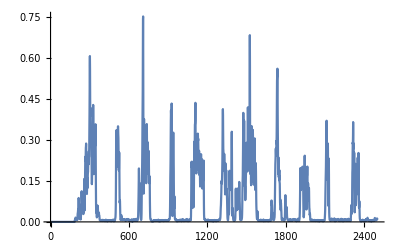

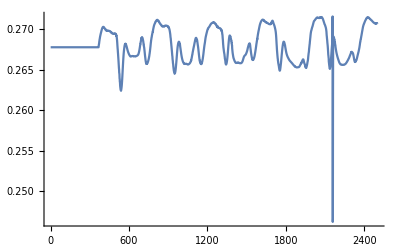

Sub03_(5)sts2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917652.0.0100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917653.0.0200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917654.0.0300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917655.0.0400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917656.0.0500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917657.0.0600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917658.0.0700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.265917659.0.0800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176510.0.0900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176511.0.100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176512.0.1100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176513.0.1200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176514.0.1300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176515.0.1400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176516.0.1500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176517.0.1600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176518.0.1700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176519.0.1800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176520.0.1900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176521.0.200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176522.0.2100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176523.0.2200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176524.0.2300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176525.0.2400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176526.0.2500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176527.0.2600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176528.0.2700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176529.0.2800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176530.0.2900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176531.0.300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176532.0.3100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176533.0.3200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176534.0.3300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176535.0.3400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176536.0.3500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176537.0.3600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176538.0.3700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176539.0.3800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176540.0.3900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176541.0.400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176542.0.4100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176543.0.4200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176544.0.4300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176545.0.4400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176546.0.4500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176547.0.4600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176548.0.4700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176549.0.4800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176550.0.4900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176551.0.500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176552.0.5100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176553.0.5200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176554.0.5300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176555.0.5400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176556.0.5500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176557.0.5600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176558.0.5700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176559.0.5800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176560.0.5900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176561.0.600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176562.0.6100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176563.0.6200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176564.0.6300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176565.0.6400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176566.0.6500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176567.0.6600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176568.0.6700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176569.0.6800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176570.0.6900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176571.0.700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176572.0.7100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176573.0.7200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176574.0.7300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176575.0.7400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176576.0.7500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176577.0.7600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176578.0.7700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176579.0.7800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176580.0.7900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176581.0.800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176582.0.8100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176583.0.8200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176584.0.8300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176585.0.8400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176586.0.8500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176587.0.8600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176588.0.8700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176589.0.8800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176590.0.8900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176591.0.900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176592.0.9100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176593.0.9200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176594.0.9300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176595.0.9400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176596.0.9500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176597.0.9600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176598.0.9700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.2659176599.0.9800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.4457719800.26591765100.0.9900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.041860925916066560.26591765101.1.00.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.05479238783757650.26591765102.1.0100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.069077359906497830.26591765103.1.0200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082998805928244490.26591765104.1.0300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.094877573542204880.26591765105.1.0400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.101962425965675910.26591765106.1.0500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104049275668415170.26591765107.1.0600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.106997934851801480.26591765108.1.0700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.119549600595491620.26591765109.1.0800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.146372483360066250.26591765110.1.0900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.183304392681109980.26591765111.1.100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.219771909448216420.26591765112.1.1100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.245354274343825060.26591765113.1.1200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.253332051268900960.26591765114.1.1300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.24284592284892730.26591765115.1.1400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.221954499561965560.26591765116.1.1500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.202785897602607730.26591765117.1.1600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.191956609854798540.26591765118.1.1700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.186378903000761180.26591765119.1.1800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.179056880503525670.26591765120.1.1900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.165072838206513720.26591765121.1.200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.1455627737590340.26591765122.1.2100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12854294344466590.26591765123.1.2200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.122936939142462940.26591765124.1.2300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.130777996853091160.26591765125.1.2400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.1432816247030840.26591765126.1.2500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14776442154873560.26591765127.1.2600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.13948095936026250.26591765128.1.2700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.124705925997187660.26591765129.1.2800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.11501772563157280.26591765130.1.2900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.118561973032483590.26591765131.1.300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.133451568918330570.26591765132.1.3100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.150655118010778740.26591765133.1.3200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.16043827401460390.26591765134.1.3300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.15811413431940680.26591765135.1.3400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.145768374279138750.26591765136.1.3500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12861984718679990.26591765137.1.3600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.111581069954072630.26591765138.1.3700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.099897504694763040.26591765139.1.3800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.097954243247587950.26591765140.1.3900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104039843695569480.26591765141.1.400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112059343747820740.26591765142.1.4100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.119207777162899580.26591765143.1.4200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.126696746514169480.26591765144.1.4300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.135364143849087650.26591765145.1.4400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14298663636502880.26591765146.1.4500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14576498835147220.26591765147.1.4600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.14313574602877910.26591765148.1.4700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.137122740292082380.26591765149.1.4800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.129030232496736340.26591765150.1.4900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.120877946329309230.26591765151.1.500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.115626206501251010.26591765152.1.5100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112847401821844810.26591765153.1.5200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.107949270027346960.26591765154.1.5300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.097622639720994840.26591765155.1.5400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.081946956262646710.26591765156.1.5500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.063987998988639830.26591765157.1.5600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0486357276002730640.26591765158.1.5700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039833671595430260.26591765159.1.5800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039523684613047940.26591765160.1.5900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.045032161885745460.26591765161.1.600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.051495578354747340.26591765162.1.6100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.056217615416670640.26591765163.1.6200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0596775585981741060.26591765164.1.6300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0622484566220604940.26591765165.1.6400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.062958496637456130.26591765166.1.6500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06415638841558970.26591765167.1.6600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06859063881455190.26591765168.1.6700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.074098872224042930.26591765169.1.6800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.080877276767805650.26591765170.1.6900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.088484125956185030.26591765171.1.700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.094217393540802110.26591765172.1.7100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.09643887841339370.26591765173.1.7200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.095649633998432610.26591765174.1.7300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.095563063923182340.26591765175.1.7400.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.101235815412289380.26591765176.1.7500.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.112094955172625730.26591765177.1.7600.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.122399596750755430.26591765178.1.7700.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.12611924569434530.26591765179.1.7800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.120038292721307840.26591765180.1.7900.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.104693333293830270.26591765181.1.800.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0845435670501440.26591765182.1.8100.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.066840769853575930.26591765183.1.8200.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0570050133311891250.26591765184.1.8300.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.054205343493466790.26591765185.1.840.0035732296219338930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.053708660436832340.26591765186.1.850.0060660733577429780.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0554936920387128630.26591765187.1.860.0083717574275930080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.06266351103568770.26591765188.1.870.0086341210077624480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.073591230504869470.26591765189.1.880.0080246740898268810.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.08388704869832480.26591765190.1.890.0128384595239184280.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.091022002083806010.26591765191.1.90.0158455667693889570.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.093108927234310470.26591765192.1.910.0149615167383658870.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.09009080890001440.26591765193.1.920.0117301416173606850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.084124252729298780.26591765194.1.930.0104020647622104990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.07827982890735740.26591765195.1.940.011731526044888030.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.073385297027219150.26591765196.1.950.0117669337337884430.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.068660537553867110.26591765197.1.960.0110566004001014570.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.063784202189089710.26591765198.1.970.0110087403363077660.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0603462396611696150.26591765199.1.980.0101944042651656820.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.058862095615896260.26591765200.1.990.0085776164712779710.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0584509506196216260.26591765201.2.0.0082263313370468540.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0571287193489699240.26591765202.2.010.0096050693399226530.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.054836137892151490.26591765203.2.020.0085019899988026150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.053609790610969080.26591765204.2.030.0067002326394310360.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.05725101491985010.26591765205.2.040.0086639132192887460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.067170390977726310.26591765206.2.050.0156059044242225910.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077705566114108210.26591765207.2.060.025742765146248440.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082171407477751630.26591765208.2.070.032207120301785150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.078057577463079770.26591765209.2.080.033120218145383980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.067868248730221030.26591765210.2.090.0396860192988922960.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.057159634582060520.26591765211.2.10.045697789524307720.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0485846952875956460.26591765212.2.110.043952893360321930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.041487910727994790.26591765213.2.120.039384972277114480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.035990118334889520.26591765214.2.130.0564546441867029850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.033454643729188130.26591765215.2.140.087761055032942890.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0356946950030537640.26591765216.2.150.078125247096848680.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.043195475496681210.26591765217.2.160.041547728799703680.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.052698631585243170.26591765218.2.170.019465528044418380.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.059022540952445240.26591765219.2.180.0125862452308814020.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0597336223885113340.26591765220.2.190.0140946571228283240.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.055037082795338680.26591765221.2.20.0200259817292355630.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.047846276072041560.26591765222.2.210.026213697328883980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0441156866290420560.26591765223.2.220.032977657497112790.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.046316757634314890.26591765224.2.230.047329853205695480.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.051242404134819820.26591765225.2.240.062612935827556350.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.055885299935030160.26591765226.2.250.060904219636600960.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0586152747495865960.26591765227.2.260.043017305377999230.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.058841978201383390.26591765228.2.270.0239455554827236080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0581785413316095460.26591765229.2.280.0118033332277701060.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.060072093085571440.26591765230.2.290.0087654558189737150.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.065655395158885830.26591765231.2.30.0109809584080258930.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.072217857514079140.26591765232.2.310.0154807414272471520.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077902367283027870.26591765233.2.320.0260153990364708630.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.082742528531383380.26591765234.2.330.043568516011686230.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.085514498669485020.26591765235.2.340.065590507206341850.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.084022467800206740.26591765236.2.350.091195917545125390.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.077780907934254810.26591765237.2.360.109244685104795740.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.069058508731816290.26591765238.2.370.112436414472045290.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.060366535123962440.26591765239.2.380.10083227898807990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0512974656920166250.26591765240.2.390.085008975530840180.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.042144183964043440.26591765241.2.40.073470563696942330.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0357733294156029540.26591765242.2.410.065599227968362980.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.035085666098133750.26591765243.2.420.062672840427654460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.037523279131669610.26591765244.2.430.05496764146163260.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039235875148661660.26591765245.2.440.0601906515353184260.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039817556831409890.26591765246.2.450.080599887561030550.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.039977193284071740.26591765247.2.460.089075436919919870.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0399923189152015940.26591765248.2.470.070523658016902620.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.040399655630865050.26591765249.2.480.043456690327640460.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.043144418298081650.26591765250.2.490.0291700218710339750.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.047057162960474340.26591765251.2.50.0287168228332372080.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.048047208532547950.26591765252.2.510.030198062825822990.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.0441887110988133450.26591765253.2.520.032039093026593180.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.038352729160061160.26591765254.2.530.035857463408108130.2677809600.366858500.3799971100.2771179800.3274690700.4954626500.3009906700.4213971500.445771980.034917974096082740.26591765255.2.540.044592331983569470.2677809600.366858500.3799971100.277117980.008801633535156230.3274690700.4954626500.3009906700.4213971500.445771980.0352002401125337950.26591765256.2.550.081633769697114070.2677809600.366858500.3799971100.277117980.0150046965510938770.3274690700.4954626500.3009906700.4213971500.445771980.037795477085091150.26591765257.2.560.137047297305624540.2677809600.366858500.3799971100.277117980.0229595350665774760.3274690700.4954626500.3009906700.4213971500.445771980.043828215412366780.26591765258.2.570.157738981063436120.2677809600.366858500.3799971100.277117980.030922638457953040.327469070.004591156959399660.4954626500.3009906700.4213971500.445771980.0555726610961621360.26591765259.2.580.119015340309877550.2677809600.366858500.3799971100.277117980.0357560400040792740.327469070.0068944108898088550.4954626500.3009906700.4213971500.445771980.069817332161366140.26591765260.2.590.065041085170807230.2677809600.366858500.3799971100.277117980.034607169721662910.327469070.0080477184684984180.4954626500.3009906700.4213971500.445771980.081690769004395870.26591765261.2.60.042412765031861250.2677809600.366858500.3799971100.277117980.0277166652500466240.327469070.0082685608787715220.4954626500.3009906700.4213971500.445771980.088279116394450840.26591765262.2.610.067187102048621290.267780960.00349779603095965760.366858500.3799971100.277117980.0196187801678021080.327469070.0064242933882755690.4954626500.3009906700.4213971500.445771980.087322434387728020.26591765263.2.620.119308143094761970.267780960.0050253762480389210.366858500.3799971100.277117980.0144487237793466080.327469070.0046967530646381360.4954626500.3009906700.4213971500.445771980.080525798603875450.26591765264.2.630.164516719877078780.267780960.005147209693430620.366858500.3799971100.277117980.0137322995723129120.327469070.0054430487671409130.4954626500.3009906700.4213971500.445771980.075176938346918580.26591765265.2.640.20351222285178570.267780960.0053504080424678010.366858500.3799971100.277117980.017399926446231730.327469070.008743730576396180.4954626500.3009906700.4213971500.445771980.080890973751489420.26591765266.2.650.238978267110087320.267780960.0074734981117466660.366858500.3799971100.277117980.0230789952101548220.327469070.0140350248186794260.4954626500.3009906700.4213971500.445771980.097546362165873850.26591765267.2.660.238023435384911140.267780960.0090917725140883530.366858500.3799971100.277117980.0267933262788423550.327469070.0195084741938742370.4954626500.3009906700.4213971500.445771980.115679225778885910.26591765268.2.670.222567158528997030.267780960.0080543941596608080.366858500.3799971100.277117980.0267385363696506160.327469070.0221156773005012940.4954626500.3009906700.4213971500.445771980.12633767817375930.26591765269.2.680.244786617433167650.267780960.0065358035671704810.366858500.3799971100.277117980.023316953043212310.327469070.0197537816506751580.4954626500.3009906700.4213971500.445771980.124618455456862470.26591765270.2.690.27173833758282130.267780960.0065099843671864970.366858500.3799971100.277117980.0177533598355931150.327469070.0155956591191000710.4954626500.3009906700.4213971500.445771980.110706781193735730.26591765271.2.70.27730450103025960.267780960.00642756356996720350.366858500.3799971100.277117980.0131508158862759450.327469070.0146537385209173640.4954626500.3009906700.4213971500.445771980.089058635249108160.26591765272.2.710.28755199067266240.267780960.005604961755373070.366858500.3799971100.277117980.0125513830711821970.327469070.0162765125212475760.495462650.0038116607054377160.3009906700.4213971500.445771980.066890950910343290.26591765273.2.720.271477157054358260.267780960.0055291102118423440.366858500.3799971100.277117980.0152934166177792120.327469070.017551300931817640.495462650.0092295973298944840.3009906700.4213971500.445771980.05209194914420590.26591765274.2.730.202777848471810820.267780960.005910363352713430.366858500.3799971100.277117980.0194686553823290450.327469070.0197433891353584920.495462650.018439565103721260.3009906700.4213971500.445771980.047856597121793420.26591765275.2.740.147742871776410930.267780960.0055537323003522620.366858500.3799971100.277117980.0223141189945977040.327469070.0216890429805002070.495462650.0271420131239389630.3009906700.4213971500.445771980.0501383984632647950.26591765276.2.750.135100229795371040.267780960.0049731111551580060.366858500.3799971100.277117980.0214144686943379470.327469070.0200795057749659530.495462650.0292461830747281980.3009906700.4213971500.445771980.0547804867035195440.26591765277.2.760.117069624848605030.267780960.0050486626368856910.366858500.3799971100.277117980.0174474055261441270.327469070.0150547416272642160.495462650.023862839587626390.3009906700.4213971500.445771980.05883384943244420.26591765278.2.770.102437580289892320.267780960.0051155693677080570.366858500.3799971100.277117980.0126286703525023740.327469070.0100191369535617360.495462650.0161939850008368980.3009906700.4213971500.445771980.0603702110648159230.26591765279.2.780.117917487414719220.267780960.0042588360983917970.366858500.3799971100.277117980.009789534363344940.327469070.0075904160364143890.495462650.0116411125007296790.3009906700.4213971500.445771980.0597253685880261560.26591765280.2.790.152906171406227060.267780960.004134789241471150.366858500.3799971100.277117980.0111564690993767310.327469070.0083777735298466580.495462650.0116536243128040480.3009906700.4213971500.445771980.061219059128039010.26591765281.2.80.16048916785079180.267780960.0050944888905496070.366858500.3799971100.277117980.0162688749454689450.327469070.0106190017594618180.495462650.0144527242301196770.3009906700.4213971500.445771980.06920103581902630.26591765282.2.810.139925959433642470.267780960.0053408472293421820.366858500.3799971100.277117980.0234725514011168420.327469070.0124660062923411110.495462650.020749744075704530.3009906700.4213971500.445771980.081264129076192680.26591765283.2.820.124309161949642550.267780960.00386850231413825120.366858500.3799971100.277117980.0295619494935431240.327469070.0123871082026162150.495462650.0279120873293193860.3009906700.4213971500.445771980.090690029346230660.26591765284.2.830.143073657048491870.267780960.00288018477748444930.366858500.3799971100.277117980.032134433193816340.327469070.0105137464768187760.495462650.0278566240326895730.3009906700.4213971500.445771980.092747566875767680.26591765285.2.840.17389210109511940.267780960.0045667898855475550.366858500.3799971100.277117980.0319025419928064060.327469070.0086916985663937320.495462650.0236207596779982880.3009906700.4213971500.445771980.08625626026792240.26591765286.2.850.18105427788319840.267780960.0070958192060700670.366858500.3799971100.277117980.031256080652613460.327469070.0088118382938423330.495462650.022770380035922530.3009906700.4213971500.445771980.07282295263196620.26591765287.2.860.18358412849911910.267780960.0080297571104349510.366858500.3799971100.277117980.0303520854909196250.327469070.0123830736833194750.495462650.027103935279706010.3009906700.4213971500.445771980.056998316517944410.26591765288.2.870.215241545737834550.267780960.0082384365916508380.366858500.3799971100.277117980.027302646271566810.327469070.01725819360443440.495462650.032254837057022050.3009906700.4213971500.445771980.044804712574404530.26591765289.2.880.24408939868738230.267780960.0092139796609875150.366858500.3799971100.277117980.0233936577358920750.327469070.0183567300402350880.495462650.033792634255687130.3009906700.4213971500.445771980.041051864418137270.26591765290.2.890.222536797580562770.267780960.0099684197588559150.366858500.3799971100.277117980.0213244622173260240.327469070.016102121427165540.495462650.035472996976884850.3009906700.4213971500.445771980.045170724784963050.26591765291.2.90.21151018787184730.267780960.0103616854238378580.366858500.3799971100.277117980.0232247125225460950.327469070.0134723844017613470.495462650.0414306460140610.3009906700.4213971500.445771980.051782411356206850.26591765292.2.910.24814914521887240.267780960.0117643561548632440.366858500.3799971100.277117980.0297471791163330740.327469070.0118883796992391620.495462650.047131969192230230.3009906700.4213971500.445771980.05603063513693770.26591765293.2.920.259336702683850060.267780960.0127467158521800180.366858500.3799971100.277117980.036172695588574020.327469070.0135971108006144040.495462650.050246775807892980.3009906700.4213971500.445771980.05601351772767480.26591765294.2.930.237264634081175240.267780960.0125203913005514990.366858500.3799971100.277117980.0410273292275729760.327469070.01968950636939990.495462650.050148579197698150.3009906700.4213971500.445771980.052742213475045910.26591765295.2.940.245782406168666670.267780960.015982015388408580.366858500.3799971100.277117980.0472622191155353950.327469070.0282459737344523470.495462650.045777613160980640.3009906700.4213971500.445771980.049631516733862160.26591765296.2.950.277210463896152170.267780960.0248605774491870160.366858500.3799971100.277117980.050567215990861660.327469070.0343461494239555650.495462650.0396920868532658550.3009906700.4213971500.445771980.052837724586090910.26591765297.2.960.33740831233806050.267780960.031272251000401520.366858500.3799971100.277117980.045940044055605490.327469070.033630917527623140.495462650.0331904966674403950.3009906700.4213971500.445771980.069655809031695840.26591765298.2.970.394296618396486050.267780960.0291099988467637680.366858500.3799971100.277117980.0397066233841009560.327469070.0273558858444035470.495462650.0290261718410910470.3009906700.4213971500.445771980.101743442816283930.26591765299.2.980.475666958218367850.267780960.0216028597478986370.366858500.3799971100.277117980.044942585556790110.327469070.0219852106725482130.495462650.028234355220661880.3009906700.4213971500.445771980.143430162964780530.26591765300.2.990.57201540528438350.267780960.0159763261082203240.366858500.3799971100.277117980.065765403872592430.327469070.0211041058265492160.495462650.030653830791691430.3009906700.4213971500.445771980.183951701380747980.26683303301.3.0.6084229866366650.267780960.0153061916067734560.366858500.3799971100.277117980.094142437317225120.327469070.0247504860429203220.495462650.0395805213670881940.3009906700.4213971500.445771980.2116087493893830.26777608302.3.010.56145065222981760.267780960.014591150049793670.366858500.3799971100.277117980.114271464817735790.327469070.0304413294477438760.495462650.048382329504245110.3009906700.4213971500.445771980.219686081386568250.26874529303.3.020.45147347275183980.267780960.0101157161916804510.366858500.3799971100.277117980.115820203559763930.327469070.035256948914608880.495462650.055049105345267220.3009906700.4213971500.445771980.207628339921695740.26974194304.3.030.390103886982094970.267780960.007827845718551390.366858500.3799971100.277117980.102973812539443380.327469070.040651200690686130.495462650.06335828090456060.3009906700.4213971500.445771980.179332783852141520.2707226305.3.040.3880816428784810.267780960.010836831499638990.366858500.3799971100.277117980.085405128942761630.327469070.045632011205621470.495462650.065925160323045490.3009906700.4213971500.445771980.142246107915702140.27170541306.3.050.402107001703424060.267780960.0163266329775882260.366858500.3799971100.277117980.069917055761781670.327469070.0441455241753830750.495462650.05685087774137840.3009906700.4213971500.445771980.104885513960006060.27267553307.3.060.417453515560860740.267780960.0187903047641541050.366858500.3799971100.277117980.063581889888999180.327469070.0371889532421955450.495462650.046425882408548160.3009906700.4213971500.445771980.073923079018642080.27363616308.3.070.36172224709366860.267780960.0153588506206207820.366858500.3799971100.277117980.070015975360755320.327469070.0316991159582349360.495462650.046283856415837230.3009906700.4213971500.445771980.053736673237094620.27459075309.3.080.27671356385666840.267780960.0128062449281024660.366858500.3799971100.277117980.082338882412888130.327469070.030575374055768250.495462650.0482762306526430540.3009906700.4213971500.445771980.047101227370290180.27554893310.3.090.290892176090995660.267780960.0146062735967511970.366858500.3799971100.277117980.093296970404940740.327469070.030122598550180050.495462650.04280784439241460.3009906700.4213971500.445771980.0554223359394387240.27650346311.3.10.33935027740566880.267780960.016705881232035780.366858500.3799971100.277117980.10325211259120020.327469070.0278875643151829740.495462650.034067504432084690.3009906700.4213971500.445771980.076428345716686970.27745659312.3.110.32789259823332840.267780960.0177255017325088740.366858500.3799971100.277117980.115883145806581640.327469070.0268077831574280170.495462650.0298154306489134820.3009906700.4213971500.445771980.103377810455267020.27840366313.3.120.266949031134260830.267780960.0160812939733723620.366858500.3799971100.277117980.129476016491517660.327469070.0279477830167076250.495462650.03300105978101170.3009906700.4213971500.445771980.12706104813276690.27933408314.3.130.20787181367370950.267780960.0116274627501626180.366858500.3799971100.277117980.13734009997294620.327469070.030393635953882310.495462650.041461867412669540.3009906700.4213971500.445771980.140647138805019360.28024396315.3.140.166693072985516250.267780960.0073031570827470790.366858500.3799971100.277117980.13971122907251080.327469070.033348861812674290.495462650.053657075049949620.3009906700.4213971500.445771980.142273670464363180.28114002316.3.150.138427703377949820.267780960.0069573820176941850.366858500.3799971100.277117980.141926288918509450.327469070.0342022960333416140.495462650.065107597484022580.3009906700.4213971500.445771980.134076865743253420.28200983317.3.160.147815992978118040.267780960.010253246717825040.36685850.00381682838773881760.3799971100.277117980.143494644014090370.327469070.034151833472279480.495462650.072440797696655250.3009906700.4213971500.445771980.122199931241136750.28285265318.3.170.19235284247451240.267780960.0130374462281818860.36685850.0061876329452285340.3799971100.277117980.138698239205874620.327469070.0342932604169501260.495462650.078254376321775040.3009906700.4213971500.445771980.115041932891076660.28365951319.3.180.248677161210113520.267780960.0122756383442933750.36685850.007255856811041160.3799971100.277117980.126404135607484730.327469070.035250199376643330.495462650.089411384253677580.3009906700.4213971500.445771980.115957323414183090.28444171320.3.190.30577949360729140.267780960.0110643434749537250.36685850.0077877384200940570.3799971100.277117980.114757733663974490.327469070.0372856244154891050.495462650.101565481316212150.3009906700.4213971500.445771980.11960731474201040.2851894321.3.20.30628216068069320.267780960.0114116891046592790.36685850.0079673476319631850.3799971100.277117980.112864760121223530.327469070.0369215893068589460.495462650.108190673198639060.3009906700.4213971500.445771980.118342309392058640.28590406322.3.210.25804348617270170.267780960.0100949674281118550.36685850.0069396237297666550.3799971100.277117980.122198594488556760.327469070.0343192046882725840.495462650.116807829042572710.3009906700.4213971500.445771980.10863625494524030.28656539323.3.220.1956965227894340.267780960.0073928080182636060.36685850.0059192635669604030.3799971100.277117980.13613856717502930.327469070.0353234127586627350.495462650.123560383567436160.3009906700.4213971500.445771980.094990328362203710.28719663324.3.230.215175863093789640.267780960.0081953338306169630.36685850.00677265620363706740.3799971100.277117980.1443260080572390.327469070.038120375005717310.495462650.118271334202577850.3009906700.4213971500.445771980.088755755389491010.28777774325.3.240.341273821946411040.267780960.012207979947985650.36685850.0100828886513489780.3799971100.277117980.142755813045055080.327469070.041446092904636710.495462650.099604254457982920.3009906700.4213971500.445771980.097660374450785530.28831025326.3.250.429147483390965370.267780960.0143532829699842670.36685850.012102667948515970.3799971100.277117980.134688936652848420.327922970.045980960140985220.495462650.078398821978555310.301437400.4213971500.445771980.115578376980726040.28861101327.3.260.371968431708414540.267780960.0133553346257819330.36685850.0106370936147950970.3799971100.277117980.123402524855137460.328300970.05006889309418460.495462650.068430765463754860.3018100800.4213971500.445771980.131280242266428450.28921867328.3.270.264004578963921930.267780960.0108947767974330490.36685850.0089568773686839080.3799971100.277117980.109996530071074420.328678630.0514835861809926840.495462650.069596246564410520.3021830500.4213971500.445771980.138359080225320920.28961008329.3.280.191748757110794530.267780960.0084564762730608280.36685850.0082261029340199980.3799971100.277117980.09527855959873380.329026670.050628497185448870.495462650.075733464401563940.3025273300.4213971500.445771980.135944463827877420.28996916330.3.290.175138705049106250.267780960.00722834243612992950.36685850.0067214213404602760.3799971100.277117980.080517515625211920.329356620.048590152888569860.495462650.082245535587045680.3028542400.4213971500.445771980.12758651238954330.29016631331.3.30.194998049742397960.267780960.00683121594203840.366564030.0048770109819904720.3796732500.277117980.067051944535522030.329644490.044086255352846720.495462650.079716905280274860.303139900.4213971500.445771980.117660631934147960.29058172332.3.310.176322564953980550.267780960.0079663548687299740.366258540.0049433604730565490.3793389300.277117980.056808535927796340.329921120.037191868415289560.495462650.069231967039938490.3034147900.4213971500.445771980.10821135477630670.29074614333.3.320.187749280480564860.267780960.009138009383847660.365945240.0062721560780897360.3790009400.277117980.05226936534147520.330158410.0311676606775553380.495462650.06038546419240080.303650900.4213971500.445771980.098781077899182030.29105437334.3.330.22744949004112530.267780960.0087117715116655260.365685330.0070695812220518390.3787162400.277117980.054131111029900620.330384420.0287946354943561970.495462650.053385620715834240.3038760800.4213971500.445771980.089641858669002960.29117703335.3.340.25192174615564020.267780960.0078548835429631660.365389080.0070417832451156780.3783991800.277117980.06373169463574010.330579790.0305275143329692930.495462650.045880117428850220.3040709500.4213971500.445771980.082406076054651290.29139419336.3.350.25500876041743690.267780960.00771109978967507350.365154820.007371281213555250.3781439600.277117980.083254424866898370.330764920.0340847822467382140.495462650.041828027383239790.3042558100.4213971500.445771980.076704325648032690.29150136337.3.360.274598619416873860.267780960.008325776293836080.364926450.008708829864878840.3778966700.277117980.110653101664174640.330931140.036834304547480740.495462650.045109567099866940.3044219500.4213971500.445771980.069821924878934350.29161171338.3.370.29949377984305890.267780960.0088292663329365540.364595380.009078071738614560.3775517200.277117980.1410103277949390.331070190.039562513294437090.495462650.054302343587282590.3045610700.4213971500.445771980.059946048670527970.29170729339.3.380.31673217788307310.267780960.0089376579115875760.364341850.0070580429468823580.3772826300.277117980.163163838732064160.331210530.041906283187021740.495462650.066208110159609380.3047015900.4213971500.445771980.04882841350451950.2917521340.3.390.29285255661341930.267780960.0100080934350392420.364143060.0053399621128544010.377067700.277117980.165043422265048260.331346750.040687972959064510.495462650.075000074776861940.304838100.4213971500.445771980.0400852989579431750.29180541341.3.40.279520625751622840.267780960.0118367523788000630.363917930.00575131835941067060.3768270500.277117980.150101020493893680.331479710.0390625244727945550.495462650.078122295607118270.3049714600.4213971500.445771980.036004815871885150.29182679342.3.410.280389279640231750.267780960.0121661235106434280.363602810.0072718276817930940.3765018600.277117980.131390893518038070.331584250.040020460613391190.495462650.078436272375569170.3050763800.4213971500.445771980.036313878139361360.29169112343.3.420.306795843836532470.267780960.0124984774107678930.36340840.009132149717054460.3762932900.277117980.116341904528140360.33170170.0412304340660537560.495462650.075973229005164320.3051943500.4213971500.445771980.041516783872325360.29170562344.3.430.35826796638436320.267780960.0141963807281041810.363161570.0101726140900884020.376033700.277117980.106143535231055260.33181430.0386016928930325850.495462650.072538524793721360.3053075200.4213971500.445771980.0501542720688481350.29163939345.3.440.30815824243968470.267780960.0136447353294894480.362895570.0095401882907136960.3757618700.277117980.09871088795493540.331882540.03241922389653530.495462650.071116601517890220.3053761600.4213971500.445771980.057817720012367780.29140707346.3.450.20497262542642830.267780960.0098149814145089280.362688990.0071392098062427780.3755467800.277117980.090800839461873060.331961330.0264283666854664150.495462650.0623769518291552860.3054554300.4213971500.445771980.061087250068747410.29126264347.3.460.121969392621009990.267780960.0060548409851487910.362499110.0042070381036621430.3753504500.277117980.07815601314756280.332024460.020470672096667110.495462650.043556632739468180.3055189900.4213971500.445771980.058645267157981150.29108843348.3.470.065866377955275720.267780960.0068635826822112910.362321140.00259408223435679540.3751684500.277117980.060085864110618320.332070360.0144465375268719130.495462650.0246495930030133440.3055652100.4213971500.445771980.051242862716067650.29088851349.3.480.0388820696500665750.267780960.009224789621375910.362168510.00294139514858543330.3750151600.277117980.04075334435158490.332091780.0113358978997463480.495462650.0127469193007463330.3055867800.4213971500.445771980.040340913362990630.29065997350.3.490.033387707288930920.267780960.0079211656854410190.361998940.00344939536446812940.3748444600.277117980.0246771874676159320.332118230.013117552601699160.495462650.0087821643782936410.3056134300.4213971500.445771980.0275564088644153770.29042019351.3.50.043979703091952490.267780960.0048827517948883520.361916650.00279129643099057520.3747651300.277117980.0148835268996133550.332108730.018238082608691420.495462650.0093279001638738360.3056038600.4213971500.445771980.0164367559243197430.290105352.3.510.045156145705635830.267780960.00324743727727054870.361777660.00225051880387197240.37463200.277117980.0134746826492711390.332087390.0252217408170697860.495462650.0104220332583779460.3055823600.4213971500.445771980.010362681170986560.28978912353.3.520.027461587285429580.267780960.00336480884953710860.361656140.0029948673647392410.3745171600.277117980.0197958211456164230.332058780.03590146761338220.495462650.0139866724188572630.3055535500.4213971500.445771980.0071013751504813840.28944172354.3.530.0165287320655227580.267780960.0031987822867015460.361560480.0045566534618595990.3744287500.277117980.0292895113862052840.332023580.0540782208979271040.495462650.0221560442928780620.305518100.4213971500.445771980.00359704948714256950.28905186355.3.540.0191684035519154270.267780960.0039164636895152810.361448250.00505431448317508050.3743247500.277117980.037446996952176140.331984010.079261264200290270.495462650.031630007968454640.3054782600.4213971500.445771980.00361467432354579430.2886341356.3.550.035773069160593810.267780960.0056638648753656960.361318690.005303110357939650.3742055400.277117980.041231676722102880.33193280.109370723046621830.495462650.0370774366131633660.3054267300.4213971500.445771980.0063138549338330880.28819526357.3.560.054964778942422170.267780960.006190758149402290.361193920.0057265782091083070.3740860100.277117980.0395319619549171840.331913940.145474604003731020.495462650.0374968373695255750.3054077500.4213971500.445771980.0062771429224442670.28769006358.3.570.0604327716395838060.267780960.0044076512022878670.361139490.0045300030039816460.3740373600.277117980.033557577815621080.331883160.170623373669560120.495462650.0371070042216623260.3053767800.4213971500.445771980.0047087497218410880.28713323359.3.580.051537542224212540.267780960.0040323183774948790.361042890.00324885313078709940.3739455400.277117980.027641279538947560.331864020.172892347338407140.495462650.038775732171142150.3053575300.4213971500.445771980.0059320303945082280.28655985360.3.590.0491519717983109550.267780960.0051017772919358320.360948140.0035435552834319510.3738539400.277117980.024966562803843620.331855250.161147747134849220.495462650.037818587694208680.3053487100.4213971500.445771980.00717636266952080.28597449361.3.60.056697072979816770.267780960.0044658209302131470.360843360.00383573175887812760.3737514800.277117980.0221891637628135150.331853250.134872872341229580.495462650.03069148762758940.305346700.4213971500.445771980.005939914989738240.28539736362.3.610.053767580848720370.267780960.0032475436724950740.3607390.0028259179276438510.3736481100.277117980.0172316665315238940.331859760.10579484953300910.495462650.0235039574389836370.3053532500.4213971500.445771980.0047694382301549750.28484183363.3.620.037393196851703720.267780960.0048193084282869340.360621650.00272158642596345530.3735319600.277117980.0129908461871388270.331866720.085959537123281960.495462650.020545490764714090.3053602500.4213971500.445771980.0064661147131956170.28431222364.3.630.028962007673936480.267780960.00684663511850210.360514570.0040934228925014890.373425790.0024767185680442130.277117980.0114107869504083740.33187440.07288830136102520.495462650.020120892629203620.3053679700.4213971500.445771980.007617649102655660.28380667365.3.640.0351149141080839560.267780960.0065492773353912370.360366930.0044788224335224760.373280350.00348143720429162570.277117980.0123052254639393740.331878890.062614258716763460.495462650.0203707280129914350.3053724900.4213971500.445771980.0059885612705615060.28331908366.3.650.032700396150895480.267780960.004369405794089150.360296020.0036190030275629280.373210850.00367563794853691380.277117980.0145127669188285550.331878750.058755261901376910.495462650.0192368616745283060.3053723500.4213971500.445771980.0043529550429947940.28282342367.3.660.0225045529131236120.267780960.00486956709853206440.360194470.00396287096995870650.373111510.0053965773863593370.277117980.0168203619464234630.331877390.066681577563506650.495462650.0162016418363611050.3053709800.4213971500.445771980.0054194576976789550.28233304368.3.670.022675794831303820.267913080.0081510496890453720.360056770.0050476507410242360.372977250.0105295533560543720.276981990.0187633323098840.33187290.085910682639769660.495462650.0127302143018808990.3053664600.4213971500.445771980.0071276497622805710.28185515369.3.680.0305452958095812320.268029480.0091023941779185290.359933910.0056316465227474150.372857230.0144637058859894660.276861960.0207718613189837660.331870330.102290314710231050.495462650.0118661811086887490.3053638700.4213971500.445771980.005626837628801540.28139342370.3.690.0339446971111947160.268135020.0084945885478114850.359820240.00532240106813123850.372745880.0120335306973763740.276752950.021587245170468180.331870120.100183630283953480.495462650.0137897488239110060.3053636600.4213971500.445771980.00327797312710994370.28094807371.3.70.027005809919624690.268223460.007972620521597080.359724420.0045546811931642620.372651950.00669304279112019950.276661470.0196338123341315350.331870410.082420671792352990.495462650.0130286398134354470.3053639600.4213971500.445771980.0044408116242752750.28051794372.3.710.0221258285225175470.268344890.0067654680390846640.359594460.004024673109408360.372524830.00378694963946051270.276535670.0155654807514181720.331869080.063801604673420320.495462650.008966358697197780.3053626100.4213971500.445771980.0044873798315859180.28010302373.3.720.0222880057990330130.268494860.0050716741119041530.359435790.00360546961796636650.372369990.00344582214899823460.276379970.0115737979612570550.331865320.0500244520896319660.495462650.004755253557407170.3053588300.4213971500.445771980.00353118182397384960.2796955374.3.730.0186559651337637050.268590650.00479302294970439850.359336150.00303632273301057470.372273050.0043799433087399680.276280350.0098772697798737340.331861080.045379607363557180.496051080.0031177995015409940.3053545800.4213971500.445771980.00608945142550643050.27925886375.3.740.0125393310857043260.268722910.0048805239014485190.359202930.0030204183432757380.372144210.0062661535668939470.276142560.011694411218363920.331850680.0568283171960422760.496627290.0022754765922231960.3053441100.4213971500.445771980.0103927125584046390.27881702376.3.750.0083949464679184280.268804420.0041483729815246050.359122220.0028512311002678330.37206640.0061138854175651690.276057510.0152548803095566790.331842770.074509175341261060.497285470.0024229059787455530.3053361600.4213971500.445771980.0135062971663546680.27834429377.3.760.0057340381781185610.268891480.0027169970161808130.359041260.0022928346179845380.371989280.00457189379067927950.275966550.0171127440870453180.331828960.084409794581121620.497935930.0044480020890536230.3053222700.4213971500.445771980.0171655246887078840.27785983378.3.770.0053534712381645970.269002890.0021318947733535440.358936770.0023656451385011140.37188960.00376696563395518150.275849980.0154365062961370170.331812050.09133868290179790.49859390.0064850568574546670.3053052600.4213971500.445771980.023250350021825090.27736106379.3.780.0055909691046767790.269090980.0037054474861522610.358857360.00274750983655833170.371814450.00360800372175525950.275757670.0111895564343671410.331795340.10661514807043060.499256990.0076500624133562640.3052884700.4213971500.445771980.0283365507423106040.27683913380.3.790.00560702139357131550.269168210.0051115239882788280.358785390.00355495822103620970.371745910.00366189695516564750.275676650.0077610736918825330.331782970.117666083735922790.49992080.0099825392369024480.3052760300.4213971500.445771980.0294015612003714070.276307381.3.80.00533437448931818950.269245250.0044931893730584690.358712760.0039019914998706850.371676620.00343520380203326270.275595730.0069233328303990030.331771390.115325968245713840.500566150.01376673675056770.3052643800.4213971500.445771980.0268027582977630530.27577608382.3.810.0055992865700519840.269321550.00285941914422751940.358640050.00269980970914038540.371607120.00278269977796153380.27551550.0066028362441728430.331760630.107815786467985660.501182630.0159518251730936570.3052535700.4213971500.445771980.0228385877262206950.27525773383.3.820.0069162725007097290.269389790.00312981476603213470.358574560.0017386144807447430.371544450.00196502531034111440.275443660.0063545679821886470.331751410.104311270765664040.501770570.0152149119043089330.3052443100.4213971500.445771980.019799927912937380.27475242384.3.830.0066856360110165340.269466510.00375240250197541840.35849990.00158178054951413460.371472840.0026579300611464850.275362820.0069362897559035240.331742010.103236626457070890.502312740.0125360165206158460.3052348600.4213971500.445771980.0170563107504138850.27427823385.3.840.0049280125866582120.269526270.0028508308277157490.358442740.00146531183661364440.37141820.0032229939569236240.275299780.0078147507055928020.331733630.106687095063284030.502818650.0115040929140417890.3052264400.4213971500.445771980.0149572955367343070.27382646386.3.850.0046324941433318950.269592670.00181601598091796580.358378920.00158404643517313560.371357160.00246785264857653840.275229670.0081222481869788440.331724580.104801179826532090.503288290.0131006272666730740.3052173400.4213971500.445771980.014422980777739350.27340302387.3.860.0060234673378411180.269650030.00279563950706395370.358324210.0031193083032388490.37130490.00283221175295777370.275169060.00770424911315275960.331716310.09181656648125510.503733250.013917586861071590.3052090300.4213971500.445771980.0141383383845924730.27299235388.3.870.0062339686773080060.269724180.00375055217784845330.358251460.0048574776875816040.371235080.005754142842806980.275090620.00723095926319180.331707570.078558263311552150.504147390.0145784722298400780.3052002500.4213971500.445771980.0128148527273909130.27260624389.3.880.0051591358531211870.269780060.00301828309104016330.358200560.0046462496863827040.371186920.0094777329784219090.275031450.0067070179791965450.331696990.073828684649160970.504549920.0149111346590450680.3051896200.4213971500.445771980.0105344399383894330.27223266390.3.890.00535792633261533350.269846620.00287875360021244650.358135790.00364351864759379940.371124870.0109918933581814180.274960910.0061726136524476740.33168850.074602691925551730.504923750.012472505888088550.3051810900.4213971500.445771980.0091398845365724230.27188044391.3.90.0061615475024606370.26990530.00379788305168066470.358080610.0044061220572449990.371072360.0085080810454633390.274898670.0059821032738817270.331679040.079217391716684880.505274570.0082357403590002150.3051715800.4213971500.445771980.0088280788104753830.27154949392.3.910.0058692011991105680.269973360.00384254408518674460.358012270.0049208892807680520.371006540.00589664808332818550.274826410.0059772510981493550.33167240.086195973340088380.505589570.0066841408523218850.3051649100.4213971500.445771980.006992307386512590.2712533393.3.920.0060080574695923880.270020030.00338633055361644560.357970670.0039173472584239350.370967380.00416508578624590150.274776810.006743441743194710.331662480.085199958940244060.505917240.0100311946015169440.3051549500.4213971500.445771980.0051230297559481390.27095934394.3.930.0072255045639655340.270067410.00404209295091885550.357926680.00317753861462193640.370925640.0024358639448734470.274726420.0084453655439238750.331654160.080615267767667230.506224820.0144530514202306970.3051465900.4213971500.445771980.0061395872687184590.27068889395.3.940.0076494423225955130.270119130.0058260993110839680.357877180.0044072560889497050.37087840.00272304123273785880.274671390.0109942101127925240.331646560.081515177892724960.506524690.0165265149471903770.3051389500.4213971500.445771980.0079151725506901830.27043438396.3.950.0057039752029852310.270160460.0064250650203336610.357840320.00526004636140352260.370843710.0044362664134806390.274627380.013039282717555990.331637720.085480355727711980.50682890.0162127418062530770.3051300800.4213971500.445771980.0072779043908506930.27017828397.3.960.0033840547448028020.270189770.0046906840970183390.357815520.0034063795170880990.370820630.0059014019555915930.274596150.013030896365450950.331630090.096538051524142650.507131830.0157746747075206630.3051224200.4213971500.445771980.0047133712989392310.26992626398.3.970.0033241804437344380.270223230.00287832061268051540.357783840.00081905541053524380.370790470.00696508605166361750.274560480.0110747194940411480.331624770.11272309345220880.507420030.016496208801550250.3051170700.4213971500.445771980.00438999147911280350.26968637399.3.980.0049575266640064770.27024780.0033736681777311730.357759920.00116440376850816580.370767590.008512588513602460.274534280.0086816403166709850.331621510.121964394365280210.507692830.0175528266858285260.305113800.4213971500.445771980.0069797464432033580.26945964400.3.990.0049574626385446450.270265920.0039145601900795870.357740520.00236723466924215230.370748720.0086452093821826610.274514950.0077439400635332830.331620880.11340649497377210.507943970.0164870817386018680.3051131700.4213971500.445771980.0073334258663272710.26925124401.4.0.00371994944280862630.270287510.0040690728566227020.357713680.00236077198167058450.370722010.0066911940151618750.274491920.0075136353227295670.331623920.090576189962272510.508165690.0122731346297519740.3051162100.4213971500.445771980.00523447185494561350.26906652402.4.010.00388873810500184450.27029630.0046559483512587230.357698110.0022067725652085290.370705880.005074608884156310.274482530.0070268599895484720.331629830.068056204169864080.50838160.0079051554191566230.3051221500.4213971500.445771980.0043849378911914510.26887873403.4.020.0065676545532790990.270297720.0059905142282898170.357686090.0030112735387849550.370692510.0053776741192719220.274481020.0076100185153236780.33164040.054525600186649930.50857760.0080261628573681920.3051327700.4213971500.445771980.005721194377974780.26870448404.4.030.0071500842139298430.270301470.00593909422343598050.357667170.0039254926218622420.370671720.0071559441863989530.274477010.009247236097689940.331655330.050193903760120040.508745240.0126385048178062260.3051477600.4213971500.445771980.0053995114875410640.26855156405.4.040.0050719866866796620.270292910.0043214344898363050.357659440.0046315699089153350.37066150.0127785910949390940.274486150.0117718158014711840.331672680.0491287221184413540.508911120.0166590350807188960.305165200.4213971500.445771980.00302289122400629380.2683944406.4.050.0048348755971000060.270274720.0064253929180294520.357658490.0071607939305290890.37065730.023865400144160910.274505570.0147652188324667350.331693930.0458413351983955260.509071740.0170857027906735070.3051865400.4213971500.445771980.0035712879305025070.26824249407.4.060.00551842769820882950.270275640.0096292562227790980.357634990.0099425282927026650.370630820.0312018470775557370.274504580.0174221183904816960.331716590.048136605129107850.509135630.0163668433272255650.3052093100.4213971500.445771980.0051134746344362730.26817692408.4.070.0046724319769178080.270246350.0094998768345147620.357637950.0093338327891517130.370629130.0265212457916615130.274535820.017624903304721220.331746190.060152500335652580.509368580.0178331025848956460.3052390600.4213971500.445771980.00415528450866953050.2679626409.4.080.0040035033848393310.270220570.0070387498438979210.357637720.0067844253252713670.370624430.0161925361540985680.274563320.0146411925276233120.331775060.073331786169456710.509515020.0185760800691437060.3052680800.4213971500.445771980.00319453036715836460.26783549410.4.090.0048457651028076080.270207460.0067230521101181230.357620180.0084130765287232040.370602280.010884368373718760.274577290.0114847640001753960.331807210.077456605344843760.509655930.0155442660919564660.305300400.4213971500.445771980.0047903489041701550.26771187411.4.10.0053065483575843170.270186340.0085282454522188740.357611410.0116135838482745240.370588670.0125791182221816070.274599810.0102339747632125030.331839410.06771812052241640.509796580.0118584596958652840.3053327800.4213971500.445771980.006005644219630820.26759764412.4.110.0046643215584258160.270165060.0080379338705577670.357602160.0110672491858188270.370574490.0150935416016056080.274622470.0098386356471164210.33187220.051710569967604790.509944540.0132381871309446770.3053657500.4213971500.445771980.0045176904567057780.26748935413.4.120.0035003495961552380.270129920.0043039117573321920.35760290.0083036666968704970.370569230.0147477948417705770.27465990.0104481415087165940.331910240.042680561039247510.510039710.0211429540273195960.305404020.00146804458367091930.4213971500.445771980.0024378455523549690.26741824414.4.130.0040033663268572330.270110460.00155666645075063060.357590880.0075128802328399950.37055220.011533284315346940.274680610.0125697435039801140.331943670.0435033342950203250.510158610.0283284492377005280.305437670.0031693593898678270.4213971500.445771980.00382438552383548630.26734483415.4.140.0046853677266120170.270099440.00384441802369304370.357569370.0101549162836192150.370525850.0129702209788185120.274692350.0150706944097289080.331977260.050012684307662920.510288930.029296415562494120.305471470.00300733620467289780.4213971500.445771980.0059697807655432650.26726461416.4.150.00344958769496784070.270072760.0065539636360124570.35756170.010782136318612060.370512480.015771567049284490.274720730.016862209721050430.332014190.062181997973386710.510385750.0270266547476929150.305508650.00295953509642665370.4213971500.445771980.0053046659054956250.26720887417.4.160.00260289415673321640.27006680.0070771466918432340.357531220.0091182285232480830.37047680.0212565185575638930.274727070.0167376650323996130.332051030.077459261844118960.51044720.0259455775592728030.305545740.0042981258790375330.4213971500.445771980.0038450975400404580.26718298418.4.170.0045647354429267240.270024050.0075553791197411230.357539930.0095511894108209430.37047920.033074921911341240.274772540.0144237719187984370.332089180.085382366388463440.510544170.0243310153541891720.305584160.0054182481997385110.4213971500.445771980.0048220462037186730.26712766419.4.180.0062927151051625440.269998030.006719159226100910.35752860.0110145194392491360.370461750.036833740364543860.274800190.0115531225974232370.332128820.081230996787323140.510607410.0208282816639418050.30562410.0043720178784193530.4213971500.445771980.0064730465931290590.26710265420.4.190.0056403262212002190.269973670.0042324671956817670.357515310.0105256055790444880.370442340.026676993406140780.274826080.0092308109333200640.332168530.07287284172020610.510657470.016568409182148320.305664110.00329540002479999540.4213971500.445771980.0064030492183438430.26708685421.4.20.005073336438222070.269950860.0019164263732188130.357500130.0094212608378197020.370421050.0232000373392924030.27485030.0068201891762063740.332208330.067176503327002720.510705740.0135392424686127930.305704230.0043420749554975360.4213971500.445771980.0060513930087193470.26707235422.4.210.006944055514164480.269963780.0021407578638485340.357450640.0077323840502114090.370366980.0213130984983807250.274836580.0044439740276357820.332243120.067339410639782240.510733440.0129056555245259770.30573930.0051596928979342280.4213971500.445771980.0068088190583356640.26708207423.4.220.0082865338487084270.269910570.0038539082708224620.357468160.00766166301319727750.370377510.0166742656823627850.274893070.00315712202677261670.332283540.07166560593392790.510766170.0139804903173084160.305780070.0039810109572688730.4213971500.445771980.0076162094498712670.26707359424.4.230.0069240990972970470.269902470.0038464225980734440.357455960.0087659772791832070.370362170.020290349304440120.274901670.00335733199765975630.332304310.075001220213758270.51078890.016427493308551710.305801020.0027582993595394110.4213971500.445771980.0067579542289736950.26707432425.4.240.0046979481264858460.269874110.0028442372247529110.357438650.0085208847953505780.370337410.0243416472834414660.274931760.0037055322476704120.332351960.084953850821202270.510823930.0173484693867774870.305849090.0042810329288878080.4213971500.445771980.0059426223118803990.26707087426.4.250.004503635166270180.269866380.00344400418952550340.357414810.0091691252872923380.370308860.0207348864877494430.274939960.0032264636921784040.332383670.09972832397995390.51085240.0141913365745039190.305881090.0060429660385324690.4213971500.445771980.0075146803661659720.26706224427.4.260.0045405213042621660.269847120.0049575567658996410.357405120.0135149577905483070.370294380.0189645576517318630.274960380.0030379424621108630.332413890.104851442200379980.510886970.0088501908323928550.30591160.0047949338732800410.4213971500.445771980.0080540921955894970.26705065428.4.270.0038952159372365540.269876290.0053070460268682180.357344090.0156410372944914760.370229980.0203415650968375750.274929450.0048227233641627060.332442210.094662971494536520.510901110.00525597586226750350.305940190.00221112465054795020.4213971500.445771980.00575513529798709050.26703851429.4.280.00352587574755443230.269817130.0045486913131358820.357386450.0119286995219986710.370267710.016948210632334260.274992180.0066289711641905160.33246440.076535339678193010.510945830.0053228504484114370.305962590.00252308656833385470.4213971500.445771980.0028374719230336810.26704628430.4.290.0040348398898791680.269823360.0066761051883472420.357355630.0073693907925393920.370233660.0126136499248982580.274985560.0064696730969930590.332487780.061671221250809170.510969830.0069713359645924130.30598620.0052622462119492810.4213971500.445771980.0029903553194667780.26705167431.4.30.00485711589611631350.269811710.0100504105701120890.357347370.0068778558505084630.370222140.0155800361128729560.274997910.0052974288563162130.332508330.0506740481071079050.510996880.0079739165822811840.306006960.0061519642258351260.4213971500.445771980.0045686194209755870.26705407432.4.310.004619983966524030.269810850.0092802221296398380.357331140.0082082803126161360.370203460.0190082529240801940.274998830.00509664666870306760.332525060.043522937581255310.5110070.0088541233213704340.306023870.0048668589327932410.4213971500.445771980.00342407479608103360.26708948433.4.320.00260095315773726640.269815040.0046491194193211380.357316380.008505747348099820.370187360.0186001372374865540.274994390.0054883714976519590.332534950.046348660893309480.511031560.0103662204283413470.306033860.0044666780627450940.4213971500.445771980.00054019193261447540.26710885434.4.330.00188136648968583550.269817190.00096080653900923390.357302230.008216016534882530.37017160.019234796412787720.274992110.0056288404856151790.332546420.059437901906460590.511052050.0112934255750793250.306045440.0056014063769434550.4213971500.445771980.00087437921896613960.26713013435.4.340.00243249927038170650.269818610.00170225316573062160.35728960.0070891936593252380.370157430.016588210154398360.27499060.0052579031165919910.332557190.074793214157287980.51107150.0097630495424256580.306056330.0048852797163241980.4213971500.445771980.00290195736813431220.26715121436.4.350.0025112775437860610.269806070.00319045302211036370.357281360.0060572414543860070.370145760.0136187871423636490.27500390.0050513345202623690.33257860.081621894159207060.511051150.00760635130368900350.306077970.0020862599623520870.4213971500.445771980.0027611746676407710.26720831437.4.360.00268517696617576530.269810030.00270492088565719770.357269180.0043719431798929810.370132560.0083892573707664040.27499970.004346510345629520.332586210.084860393587803150.511073520.0092270105981019980.306085660.00059223515830446070.4213971500.445771980.00128981417498328530.26722628438.4.370.0045191740607956220.269812610.00305328080989056070.357259510.0034013171223527730.370121980.00315285782467998340.274996960.00319666024026089150.332592850.099147831426582940.51108680.0124211723251456440.306092370.00207885932913049430.4213971500.445771980.0024450119422203470.26724649439.4.380.0060345915899028330.269809760.0050808635176718170.357248750.00467333201314122650.370109170.0027057198285448590.274999990.00338434167539828150.332606340.11617833812084430.511052450.0141424329356038980.3061060.0025573394308271040.4213971500.445771980.0034605186608114220.26730248440.4.390.0048995233533648950.269801210.0052390186371467250.357255270.0052326798963733420.370115080.0037080363153141070.275009040.0047203028000687090.332609130.112190650541675250.511058930.0146245847951189750.306108820.002307499364643780.4213971500.445771980.0025053713195499520.26730757441.4.40.00381962775179112840.269803920.0041526431939832120.357243690.00369732247836279150.370102340.00529522116895652250.275006170.0061254396452229270.332617470.087884647079760390.511069260.0141762874172966080.306117250.00375757533773781170.4213971500.445771980.0024095936975964550.26732524442.4.410.0055094010277085370.269823110.0061060300061045120.357213090.00262044446832519760.370070850.0085404817158790410.274985840.0078384510341546350.332626690.066129319461343760.511029730.0135108756951955960.306126570.0060096839498761990.4213971500.445771980.0046934362314274750.2673862443.4.420.00658213395630227040.269812840.0088336828504589090.357223980.0032601563774132160.370081430.0123637287943250480.274996720.009487997379289110.332627090.063136874439745360.511035350.0118623235407368330.306126970.0068230648894783550.4213971500.445771980.0064206807665396280.26738556444.4.430.0055639373763550170.269816580.0085423233313605370.357215140.00345360791798925320.3700720.0114797707088904430.274992760.009971938836880230.332631670.079333239545856780.511037740.0098463248196861160.306131610.0056290136347031080.4213971500.445771980.0046381796664729580.26739609445.4.440.0036568710377000690.269816870.0057447407245107870.357207350.00274153019046943870.370063160.0073169229840366520.274992450.0092211941296244420.332638910.103042082270005690.510987250.0097782135125031220.306138930.0042084176346162280.4213971500.445771980.0025336215623558240.26743642446.4.450.0044377907480033410.269811640.0043082504622882430.357210760.0027472504822171940.37006610.0058041530782876980.274997990.0076863675981184860.332641180.117978091866536430.510963270.0115468848336984420.306141230.00370804338792384440.4213971500.445771980.00471650728638149750.26745425447.4.460.0056210958104217440.269808120.0047759478232012490.357211740.00333024101404025750.370066580.0075577469675218430.275001720.0059056502646730250.332643980.11597374856460590.510941690.014182842398422470.306144050.0030278026895659390.4213971500.445771980.0067349433179624230.26746703448.4.470.0047692985011897980.26980340.0039119721050578040.357212520.0034067908568787810.370066630.012406496934463410.275006720.0050689620939780650.332648240.106000900741193680.510919210.018052800935248130.306148360.0016768715059761530.4213971500.445771980.0059478056076736210.2674759449.4.480.00378911455643512940.269799290.0018584336268680580.357211770.00280554536045331170.370065030.011795911400808210.275011080.0057443306134874160.332653350.091959905478125170.510886410.020768109616723870.306153530.00246120830749261070.4213971500.445771980.0053102629559701320.2674958450.4.490.00480324806449794650.269792690.0023731297307107910.357213250.00275181828689321670.370065520.0064467493832030410.275018070.0068930601940329460.332658950.073392004099070980.510852770.0181104262772789970.306159190.0039740853375228720.4213971500.445771980.007582946872083210.26751388451.4.50.005656327212678650.269791280.0046184620012620890.357213460.0048344406040980290.37006550.0048115132432983160.275019560.0086624455248688390.332660240.060703071071547740.510847550.0118978107018391910.30616050.00331253667981019780.4213971500.445771980.009275490040679630.26751256452.4.510.0046419563343559180.269780080.0052039801770626870.357212050.00623970173316761540.370061860.00664241589329166850.275031430.0110345938986365370.332673530.056642725684013560.510784370.0085588752278840370.306173930.00217732217603614770.4213971500.445771980.0079691190428575530.26755723453.4.520.00375947993491869930.26976720.0050921428947732970.357221310.0055337181213231120.370070110.00767792847011704650.275045070.0117140021034060070.332678260.0590782529944134660.510776370.0091369737271059240.306178720.0025175139416178770.4213971500.445771980.00712546279467258550.26754994454.4.530.0054540630575438260.269763540.0062712574683272180.357214730.0043337056534700430.370061920.0075447257126732410.275048940.0093813790247497740.332688520.074221029790778170.51075450.0111922079298514030.30618910.0039733027373128180.4213971500.445771980.0105008892754505580.26756067455.4.540.0062206119551465980.269744510.0065769714935550450.357223870.0041012247194627670.370068910.0098228987771676050.27506910.00639955308680502550.332699910.093973269790999510.510688510.014222845310627130.306200620.00343244785200728320.4213971500.445771980.0134317204214698120.2676067456.4.550.0047755614855607680.269734340.0047788599706430020.35722380.0034764034128495060.370066990.013152645777339790.275079860.0052470849918615730.332710770.09744600844759130.510664710.0169838344747816960.30621160.00295836549739416160.4213971500.445771980.013546969575940410.26761358457.4.560.0041283528572727630.269717760.00306991255692942850.357230530.0023970081595953210.370071670.0132939675646384890.275097410.0048498892751431670.332721860.084806938218756760.510633250.0176048478775999020.306222820.0044236399754816580.4213971500.445771980.0131209229317670020.26763406458.4.570.0053833597110047290.269702110.00363575954480637640.357235880.00222257557871254370.370074940.0095575266081877040.275113970.00359099678298757750.332733290.075748037568649940.5106090.0150645720689421330.306234380.0044129055098101940.4213971500.445771980.0133357644011404840.26764967459.4.580.0057838427757628540.269708480.0044503525098004150.357217790.0033825205481696910.370055410.0056376743044204790.275107230.00252122153108140640.3327440.082783795120005510.510592280.0114442478023113280.306245210.00231175245738026850.4213971500.445771980.013267973694818530.26766208460.4.590.0041399502005166670.269676970.00338858667122162330.357239170.00357038832019684680.370074130.00434149850115951850.275140570.00262015441933524970.332756750.093575081323465910.510535960.01037331014915170.306258120.00083580335054561650.4213971500.445771980.0115155658662458510.26770596461.4.60.00269386904636196660.269660710.0014717000898291750.357241510.00203188723092234550.370073850.00364070143181785330.275157770.0027730009060844240.332771710.091064168623982240.510489010.0112432931077135740.306273260.002159318211780070.4213971500.445771980.0091497458699817680.26774143462.4.610.00350624043214128830.269657190.00143356623420273580.357232760.00067767259372750140.370063190.0050360831356301290.275161490.0022509500436641890.332783860.076419872530668050.510458670.0101192185790626130.306285560.0041169745744359760.421397150.000342132539021986050.445771980.0093223468580940180.2677616463.4.620.0041012937775498650.269632180.00265580847043137050.357246840.00160002893346591080.370074740.0088657827674325490.275187930.00241559406149665850.332796740.06570279003283940.510395940.0058774215614517290.306298590.0037429541319006790.421397150.00059545561531673180.445771980.0119797146896573020.26780338464.4.630.0032246075682510120.269614340.00245712410743057330.357254120.0028742779664457160.370079820.0093538354535300270.275206770.00387098000842531430.332808560.063559932709852370.510346190.0025269201121648940.306310560.0019102516558535370.421397150.00063382123873726270.445771980.0141214141796456360.26783359465.4.640.0026131438575429430.269600090.00171388800451929680.357257430.003070161246403220.3700810.0062642438369986070.275221840.0051352538056107190.332820430.065201005777001570.510283390.0033301983024507140.306322570.00155600814102919980.421397150.00093633301092530670.445771980.015970325737644660.26786669466.4.650.00338874614337138270.269604940.00322762081361044040.357244230.00302892183214494840.370066780.00557192720309988760.275216710.00621070647893079850.3328280.071586387790232330.510264460.0041539464443699460.306330230.0024858540537045160.421397150.00140681464457699520.445771980.017421989239087910.2678728467.4.660.00425863673881612950.269566360.0052964684916670950.357273230.0029139819685437810.370092930.0087037326940504480.275257460.0076870242074141490.33284080.086438862915058830.510170750.0058799119972744650.30634320.00261890344455221630.421397150.00140682021009801930.445771980.017329679390019870.26792553468.4.670.0040889011627847110.269568710.00514432374138530740.357266140.00195712527110255370.370085240.0098956564925056670.275254970.007859136455668390.332845130.10078144721862030.510151990.0099932813659556680.306347580.0033879676558180870.421397150.00104817847319196030.445771980.0149083146681969930.26792874469.4.680.0045445121065489320.269530390.0043090890500336820.357293190.00135976428014499320.37010920.0103496961675683730.275295430.0058441241930785470.332859510.103366439869445090.510042070.0127757838967211740.306362140.0050104579768538830.421397150.0011652121623412940.445771980.0120660655173569120.26799579470.4.690.0050978024284365260.269508480.0053232683221233670.357308670.00300092401695212450.370122930.01865552963881160.275318550.0041942998769863260.33286770.094953615251529330.509974450.0124223231537801370.306370430.0043797456405213820.421397150.00150271931326666240.445771980.0099413567857624260.26804388471.4.70.0047425193383481280.26950280.0062345666694678950.357306390.0060770799578186010.370119280.0243757934290490.275324540.0053674150945566680.332875860.08683206070171390.509882060.0115530623699559160.306378690.0031233021145898790.421397150.00115212870031459790.445771980.0072703830833050440.26810927472.4.710.00380117727610111830.269487060.00453462957119800040.357327160.0071570325246366730.370140190.0166078010730328140.275341150.0065542168904705390.332872490.088378845114757060.509878750.0121234723119975260.306375280.00428052089328756140.421397150.00074185136920171770.445771980.0041928359071838280.26808186473.4.720.0037356360901253180.269483050.0026950613017592180.357311390.0062122860104202880.370121390.00762777094628234750.275345380.0057374465083535810.332891830.106282182999693050.509667530.012132290703749980.306394860.0056342867598901840.421397150.00115989989971498460.445771980.00333909512414229440.26827135474.4.730.0051685702907497090.269465990.00297501047521601170.357320750.0062858093356727410.370128980.0071864520435510480.275363370.00491159536564304050.332900780.13384282227633240.509544970.0116082319675170770.306403930.004209116931576270.421397150.00140474929634480920.445771980.0040432988591771640.26837246475.4.740.0064465772118106110.269465710.00321699206388701560.357313380.0060192779460217480.370120490.0083109613457218110.275363660.0056187018197412070.332908120.156573928846495460.509399510.012380222047590610.306411370.0026647421652811990.421397150.00094357469585602060.445771980.0037263837723174470.26849059476.4.750.0060706645035105390.269455030.00248631091848693820.357316520.00380086145226766170.370122130.0091898624471942140.275374920.0058081742108346710.332916320.178685435787014730.509250540.014017827081757510.306419680.0027721406893171190.421397150.00060524684474102960.445771980.00235002446760846540.26861548477.4.760.0061543974436280160.26945640.0021935543109448760.357309480.00178662764375944080.370114320.0093107584526696370.275373480.0042690627971638970.332921630.193968937659589250.509084270.0147826917607391290.306425060.00324131021015968330.421397150.0011708130754395830.445771980.0023464503741528180.268756478.4.770.0080858165245305260.269445070.0036230833709844470.357315810.00231050740155851150.370119480.008044967548593240.275385420.00254864794952570050.332927450.180859287247735260.508915940.0122012205770706140.306430950.00308230620559413930.421397150.0017935809407504090.445771980.0045904675186784750.26890008479.4.780.0086210610167394130.269448520.0057544804891732960.357309710.0043491903167709930.370113130.0125347608813391460.275381790.00255557537090829150.332929680.147825807229645640.508716920.008429955771338220.306433210.00338036353447804080.421397150.00188143085776663630.445771980.0061645481317362030.26906254480.4.790.0071099569124683060.269437560.00529550497152508560.357318630.00462090015043229750.370121340.017500017945533070.275393340.00281187441974741540.332932630.128659789467157640.508510890.0087825646790762430.306436190.00365652056669788470.421397150.00160600792489192130.445771980.005419478495529040.26922873481.4.80.00544064914773666540.269443020.0038962541253998420.357311980.0033480045528982970.370114720.0177939801996077270.275387580.0022235626982779140.332933270.128453704825533730.508283950.0128428350651708640.306436850.00435937977723034350.421397150.00152171464233271650.445771980.0050329650808088530.26941392482.4.810.0049802216463233080.269427690.0040947548895554890.357328540.00285799114996614650.370130880.0113611738662828880.275403740.00200069221379030850.332933490.133396572621011480.508043070.0159839478507078460.306437070.00450622598088538850.421397150.0016410257399820860.445771980.0062524731460428650.26961048483.4.820.0037582657533669040.269423120.00413736176964932260.357334730.0033821344798411720.370137150.0053569969050881960.275408550.0029076998624613930.332932340.131465124142248120.507778170.0159619825071994830.306435910.0031643423815601980.421397150.00123593848477649520.445771980.0049352578793517610.26982321484.4.830.00215477906959548550.269431140.00265517239810078840.357326470.0029079763247198330.370129150.0030583445986386180.27540010.0039435875205476280.332931850.123017599292364030.507480770.0159866344963212130.306435410.0032973023683633380.421397150.0006781074737596780.445771980.00281216466105944530.27005216485.4.840.0032386051144272190.269437250.00243240927528840440.357322650.00184501247345526070.370125890.00161823609554194860.275393660.00359979631182835320.332929110.116681224569282550.507165870.017852067613213030.306432630.004595828315902890.421397150.00076555510503232540.445771980.0030866845033732760.27029663486.4.850.0051641757181190860.269449450.00466161758899099640.357315160.00248633817305299450.370119550.00148022866840442960.27538080.00292951031432812230.332923480.116226179733499270.506828730.0179823931593201330.306426930.00355871800448108630.421397150.00082147821244193870.445771980.004340920383510240.2705515487.4.860.0047668858175758230.269433890.0054684698603299620.357336330.0031679594491479770.370140950.0022990393152979850.27539720.00339412860596078650.332919530.122608399363155670.506479650.0172175531652712060.306422920.00159748618183630.421397150.00062120392191996930.445771980.00364291719701799550.27081479488.4.870.0029898870612678340.269454620.00373490613465418760.357323160.0023415296801330570.370129670.0020343247443228160.275375360.00369341420819085160.33291040.133165398431939860.506100910.0167704959466840370.306413670.0028454045369624440.421397150.00053223994674212570.445771980.00182590426417213420.27109591489.4.880.00315301352555815180.269457960.00297273823302437840.357328110.00169131062769367520.370135950.0012126284300037820.275371830.00287552897712680570.332902140.139444293536071960.505701080.0148206160652666510.306405310.0054233052171420970.421397150.00091604240202138980.445771980.00310055253315327970.27138845490.4.890.0052934617835566630.269462230.0036896213728658340.357334040.002618079005473550.370143520.0014529920491578770.275367330.00298195141374357460.332891980.154972633115269570.505273760.0117180460281680310.306395020.0050868234217020630.421397150.00083231184622970040.445771980.0050026052090834240.27169541491.4.90.0054603593841249660.269459160.0030693971531856450.357348630.00304067163958093080.370159680.00238269398480657960.275370570.00497921062691746450.332881210.18149930862097520.504815470.011346294730901850.306384110.00253972972605538350.421397150.00025120925616847340.445771980.00358604939503927430.27201971492.4.910.0049144794821814830.269466340.00114004176207018330.357355070.0018661383755392850.370168370.0023348697381165070.275362990.00606072459748570150.332867470.198222923123313740.504326930.0146115074388941060.30637020.0029430451776748970.421944860.00047603220768234110.445771980.00128203384624373230.27236015493.4.920.0075891867137390990.269436890.00091681229279281340.357401320.00064218035208450880.370215950.00113666153998934880.275394040.0047152827089462220.332854030.19630849984964910.50381620.0176792773550993630.306356590.0054622911204698850.422517430.00127228691449992460.445771980.00264612357416429920.27271707494.4.930.0110723038401863320.269430150.00267764159971553040.357426470.00111080766435609930.370243510.0009736222528730570.275401140.00279215769341193160.332836970.177861682879372820.503274930.0171464979478461420.306339310.006138984801649640.42312160.0016011886433608590.445771980.005660698643125310.27310093495.4.940.0131282821433506580.269465930.00340484947345126360.357410650.0022209435960000780.370231930.00266639642913113570.275363430.00290907809793705670.332814490.149698161485467270.502690170.0135535319022096630.306316560.00592143737668908350.42377170.00130414696878393840.445771980.0061040519475526850.27351097496.4.950.0150269326273517470.269460110.00262102767648896350.357439750.0021844972872266580.370264170.00325151867385256020.275369570.0039452578698155590.332792630.13112792900520690.502085170.012028995506368930.306294430.0065879858608569250.424442620.00118308143938305960.445771980.0043075311022550070.2739391497.4.960.0204245475406219340.269452180.003003053679019570.357473660.00182502477039489780.370301540.00275198990153632550.275377930.0043958598678715930.332768320.126149294238994540.501454020.014265000504484470.306269830.00630028548834199450.425140350.00169481374258801610.445771980.0037515211408851540.27438449498.4.970.0336695280504790350.269372760.0051986416511901320.357583690.00277056546406281940.370413030.0036747221019720070.27546160.0049460358589910030.332746040.11033546004380960.500809680.0147539837173288920.306247290.004678512155641720.425850350.00176807829796147190.445771980.0054464997866685230.2748371499.4.980.061816553069988540.269363840.0067520603890455660.357617810.0038197076370127830.370450440.0062923282292090690.275470990.0060480859763630530.332722530.082052465140643950.500134820.0119462770471194160.30622350.0039283369214613980.426598950.00116849514329932520.445771980.0083915948808936050.2753171500.4.990.122887674859492990.269388340.0066713828097485810.357617290.0037098703936404430.370454270.0085446151324004280.275445190.0071842509137983950.332697130.057037790566987660.499416140.010676418102336970.30619780.005261774510443310.427384980.0013089839031871220.44666750.0137945123112074960.27580828501.5.0.224262413343401830.269355610.0080010886525477550.357674560.0046158556157650640.370513840.0102140816144551270.275479650.0092291053384684560.332676380.0374736293041674150.498695960.0122169356642976950.306176810.0067175921739374550.428176410.00237666682507662630.447563730.023122845120663840.27631234502.5.010.32016201905387420.269193150.0122269562295421260.357866160.00688066923557654250.370703650.0130796342268457640.275650470.0130898230438149680.332662810.0228105231526951060.49798710.0155114377750335560.30616310.0062151535702773080.428950660.00309792291693723530.448440890.033882250987436750.27681032503.5.020.336120136358397270.269266780.0145809525563120910.35780630.00765849391770616950.370648450.0152578284231173030.27557310.0177976606934153940.332642870.0141657227937678120.49719170.0191924662197654470.306142930.0050012958563114780.429825510.00274862350782519240.449429740.042365469406760310.27736162504.5.030.29021898535290090.269206910.0136166012603183470.357881770.00614486799645771850.370723970.0147047793698814030.275636020.0215839595603949460.332633120.0113974156227150680.496409550.0199564251912741840.306133070.0059980976060644150.430682960.0021685502932619930.450397340.0477182699624715550.27790659505.5.040.271109845913481140.269137390.0124110849256646190.357960090.0046968995978676020.370801010.0127244851248549010.2757090.0238229895135413340.332630790.011613918097816040.495604310.0179962718579684230.306130710.0071236053988751360.431566260.00201062142115356920.451390860.051708855737608390.27847169506.5.050.27715022595098120.269040520.0112170202135282640.358059950.005538439932196210.37089780.0109590538012824550.275810560.0283162394689902840.332636410.012658404064535450.494774920.0188345389641315850.30613640.0064034395689324940.432475760.00163258088467214960.452410670.055930440921640510.27905966507.5.060.279793173161691060.268916770.0091887469002532080.358181050.0074938498911504460.37101410.0098596864029178180.27594010.0425939079620617850.332649720.0149657588333714770.493918610.0274281488745847060.306149860.0061729073323294050.433413060.00141176582632835530.453459260.06051113910714670.27967283508.5.070.2577021314904810.268757940.00773775629030933750.35833140.0078689586166377140.371157610.008884719994882180.276106020.067492255283994930.332671460.0203135169420498760.493036370.040191412139198290.306171840.0078079527414543760.434377060.00243910008696999240.454535390.064917489005845220.28030908509.5.080.22172153008336090.268575260.0072968764941665670.358500310.0068476628899960220.371318180.0073179464298884550.276296370.095864141460015680.332699960.0292499351524463660.492126160.04942540377226060.306200670.0106044349919749030.435367540.0039597641203006610.455640870.069112069051801740.2809669510.5.090.203758673707075950.268361490.0069693739412657360.358697450.0061735778745712090.371505590.0063408532808267550.276518440.120665199111113660.332733280.041395406923189950.491200880.0566904170074931870.306234370.0118933258792841750.436367490.005174073883695150.456760390.072496558481062660.28162424511.5.10.23551616396112870.268091740.0062360177978794490.35893880.006921001584344080.371733790.00680550625221058250.276797680.140874646551894470.332781660.056125026476162210.49030730.068582110329807710.306283320.0123862575285982150.43732820.0059400494926123820.45783580.074890854681724710.28224827512.5.110.290556788401823360.267862610.00764330068091316050.359160550.0079905733912630680.371946950.0086998867810052090.277033970.160163550773951340.332805890.074493390482907110.489383970.08884192751978840.306307850.0136323538150602240.438316660.0064619995771645820.45895010.079204799551197720.28288795513.5.120.3260976148235660.267637550.0112688254106237760.359370120.0085846314982189020.372147010.0117651361608646120.277265290.178507398728205370.332837040.097290293969756680.488496760.123613911444655530.306339390.0134765144052703820.43925820.0067783173284589210.460015910.092269395147422580.28348667514.5.130.336220976187516060.267463930.0135840310719638810.359533930.009948027624326880.372303910.0141647532405491920.277443190.194425820872620340.332858570.116410648335582480.487646540.174604414441201760.306361190.0120231462866162780.440154610.0070013484383442340.461035530.119546631140302160.2840589515.5.140.34099628492065710.267202030.0122982553718753390.359789780.010494882245432690.372550760.0142253577844842860.277710680.214041756978948530.332881980.122952158377414520.486895570.222248660093915250.306384890.0121720955674949290.440942550.0079709142334517970.461934180.158531338619341180.28455276516.5.150.35082742060430810.267012140.0103012869750487430.35998150.0092618462149505220.372736990.0127452046014149370.277903960.238455201851351270.332892480.112970811089513870.486190670.241653826636040430.306395530.0156169582256546830.441677610.0099747108151268250.46277720.200602093955816460.28501918517.5.160.340516897034104260.266763770.0106478674557423140.360229890.0084842794998146280.372978030.0116539853912711340.278155930.25683192328225520.332907860.094928384847783380.485587620.231449263667084850.30641110.0219078206284808630.442304940.0113429346823440780.463497660.233500352936411360.28540531518.5.170.320891375822347670.266525880.012016928686608920.36046590.0086551383181539440.373206890.0115107327480486360.278396370.259014741447782140.332923740.0799688314492380.485065550.202813601845300560.306427190.031060601575179850.442846080.0115092731970862630.464121140.248442885652400940.28572802519.5.180.30749991578544310.266285890.012123313365991010.360701020.00753195592781167550.373434520.0118840856728441540.278638070.241936657817328450.332941950.077561368222326570.484619390.177492889018899730.306445640.040565916361011690.44330640.011336235186324360.464654430.24722554199020210.28598229520.5.190.26743421507675060.266032370.0107407637773747670.360944650.0059262379086241770.373669740.01111266864645660.278892430.212455578478048160.332964980.08573982361966940.48423980.17178471861654640.306468980.046329642292081540.443692910.0115570585063097770.465107090.240736065664473450.28617043521.5.20.208893671987286170.265767170.0097902783117513460.361199770.0062657796687289870.373916320.0101201935203185950.279157460.185067573006453550.332988010.095882151067945520.483948540.17906108604759810.306492320.045606744694283980.443984780.0122411543437766310.465453520.239312464032028880.2862909522.5.210.189189840401135150.265496670.0095796221805373280.361461890.0072780068778688450.37417020.0102081295127909760.279426660.170380133864466150.333008830.100102863647103720.483717330.187497070241165520.306513420.038714825365667540.444213480.013880029463041660.465731310.245407773260963140.28634718523.5.220.193425038384523960.265207480.0083177655436543730.361752470.006554072312787110.374453740.0103218805383754260.279713250.166188025565008220.333020280.092052132128722390.483552760.189541969076057050.306525030.031329460872261930.444375790.0154353127475369830.465932440.254856981214048870.28636489524.5.230.227222800725320250.265060390.0069094366302481620.361938260.0052524107408155370.374641640.0103126879997927220.279858520.164565966664679130.332989480.075668434200166740.483502930.18226430224067990.306493810.029724651415249920.444413860.015641388614316360.466005820.262004279746816670.28629087525.5.240.25480823847014190.264656350.0078042371130064990.362355260.0060049762460060250.375051040.0103197998210787110.280255880.164419440204719080.332992690.063538755402543760.483448520.169284053865118050.306497060.033854847175343570.444476390.0150350238875648630.466081750.26333060890606940.28626312526.5.250.224803710124996970.264562640.009471595618229510.362516710.0079474002045355220.37522030.0092908977925141840.280347680.163947179561274860.332931270.059428280627794530.483506220.154172926002489830.306434820.039056335032106530.444420290.014092854230280120.466038010.261003443178869530.28616186527.5.260.156243359694350630.264402380.0087480156888938030.362754010.0088433947425186270.375465280.0079329700883980970.280504380.157791219762875940.332862920.059278451250867280.483580950.139938323491272530.306365590.0423940427110368750.444351310.0125531381130182580.465977780.26301117380645960.28605232528.5.270.096668310622352650.263932240.006172054399837730.36328440.0067972485723398270.375994390.0062434920595718550.280961810.144160116959092340.332819520.056925860472670530.483824650.12497119665224380.306321650.041762227230520390.444117760.0113148614015562250.4657140.27506197603244930.28584248529.5.280.070255286265223140.263855070.0057252565061337490.36347980.0048056150610315130.376205290.00523145993330465750.281036580.129883696704687630.332707670.05111340068642270.483943530.109393545129156150.306208460.039044627254780960.444005640.0111398290259183460.465611570.29200555645719460.28571234530.5.290.076669348934223380.263516540.0071911639469139610.363916510.00514351428784356160.376649370.0059839193052151910.28136350.127010992452745640.332621230.045749701225741110.484338310.095846242904582750.306121060.038705429043288680.443615890.0113690649035730620.46517930.30221149394511240.28538817531.5.30.077823754526786790.263433340.006694705208743370.36416250.0053688283567513550.376916950.00657635097275998440.281443580.13424437906348250.332464720.044483051890007170.484452990.087446485003835920.305962920.041434035398138150.443503720.0130742941633281270.465092770.298740904546826340.28523269532.5.310.0567104297355584750.263089710.0050250701843278360.364658080.004361131525282060.377427560.00615284158525440050.281773220.144533711294270980.332323050.0469693651935773750.484901050.086926513040648590.305819920.045640096225672220.443050580.016269771436235210.464608210.286064886512314760.28484151533.5.320.031782622725899520.262907470.00582906224199595660.365050370.0051028014966358950.377845830.0065192807899669670.281947330.154929908812343030.332119090.04932916931561460.48518510.097380368803912710.305614290.047877421950972690.442755730.0183444358542033320.464330950.27800245460646610.28452221534.5.330.0169591729443301160.262763440.0080336255806895110.365434820.0100103070294739180.378260720.0093981356850850530.282084580.157862927431907550.331882020.046265031527717670.485480590.110863876396922520.305375640.051011552220138260.442437480.0193990452598693870.46404180.28544188500306240.28417463535.5.340.0097131399980091640.262654050.0089085891153426780.365846960.0149922203069676810.378711670.014938434058378450.28218860.14859017240103620.331578770.037477871485240360.485723380.109933824506335560.305070880.0571108834372736560.442157220.020942386570821770.463827980.304781221521684850.28378562536.5.350.0068527528011349440.262527680.009130261621003360.366309480.0156340218684551740.379216220.0227838692323432120.282308560.136771000030634530.331237410.0287676974654784460.485999390.098236437118007250.304728510.06485328177027880.441830030.0231813957032308840.463574960.32195482884424760.28335142537.5.360.00803021935192810.262483690.0115935025833997730.366729280.0131376742764796760.379683350.0311394497435738970.282350260.13682087843423850.330848610.0260079620453380170.486250640.090310498567160560.304339440.072161800684862650.441512170.024044537678036740.463354750.32440672969176090.28287936538.5.370.009999467291167110.262443090.015981167042494880.367207680.0185973641095850480.380215390.037630333354699170.282388720.142333745424387060.330387570.0282549673039909880.486225860.081929066685422410.303879220.073166144311948580.441465240.024597485115340270.463470760.308884951789324960.2825469539.5.380.0111485156219534360.262473550.02654954824503730.367617710.0375156461190589360.380678750.047093831344624520.282359860.13388825442495330.329914030.0304103338319725440.486724880.06829701245199730.303407730.064475845346926030.440851240.026840887027333430.462952030.282787049919262350.28178834540.5.390.0161827543473726560.262446830.046113145099360510.368171560.063153614564242160.381293120.064833059518677340.282385180.108670580556445360.329336390.029101222964729350.486614020.0542599379125502860.302834190.051229931975693320.440851450.026479568125544350.46316760.262132941285394270.28140845541.5.40.0234183587433075960.262591980.061616201979564050.368537660.078245083376003390.381718210.071735115136978350.282247550.082080828539008850.328761420.025445536771513960.487165520.045060140731443540.302264890.040419559996561770.440137170.0208147731179921140.462573250.263130576671890940.28052308542.5.410.0244177873511189840.262679880.0584256812033318650.369025470.06777702788563860.382268530.061997513768946690.282164050.069941228961852450.328099920.0241622123627238570.487381780.044434350251749970.301611790.036871148525573550.43974420.0144421386673734340.462373120.28725621169986430.27982983543.5.420.0197553168959601270.262805190.045337128082918590.369513080.044142861308662040.382820020.0537361756093672140.282044820.071604552810510970.327377350.024193316271653220.487620070.05344028374408610.300900510.0420518725760729640.439294660.0133476210239430750.462131060.318214719687816340.27907148544.5.430.0150507118639006550.26294580.036012535090482360.370014580.032549455770843610.383385130.063442317778164450.281910750.073983500195361210.326600110.021575162948703390.487839580.062138164260248620.300137690.051850948584999990.438830750.0168309424872227950.461891610.335669543303358630.27828818545.5.440.0132263658419715520.263128590.031823024536398570.370503810.0375972637842709040.383937770.082561025141698760.281736020.072117634713260980.325763360.0180343626170585030.488038780.060836754029389460.299318930.0598372875447012450.438351220.0213737315462923170.461655640.326655316995794360.27746714546.5.450.014085301219429840.263347490.0330032942553572660.370979940.045397356368136030.384475920.090407986029203510.28152610.070147189473776640.324872690.017486444046054940.488211720.052891389282666980.298450020.064186361036838650.437861060.0237725836065676920.4614280.29040446686474770.27661004547.5.460.0122869451297952290.263585950.031728280254859760.371458890.040191597012528360.385014830.080031641643681820.281296610.071085546948590010.323928450.0195601753499642650.48837480.048320733614746060.297531760.062670858980172060.437346550.0229861837519028460.461189660.238223392135932160.27571828548.5.470.0085427259620943220.263855390.0250693061843465760.371919830.029189819136566440.38553270.074261259265222440.281036270.074373268655180850.322943290.0215006461444588630.488546520.046101747983151580.296576890.0525706336439146150.436791760.0217726227435047320.460920130.188713800936838040.27478296549.5.480.0073983771509838890.264136020.0177506490071741120.372380480.0227111227895766470.386046440.076956596365453040.280763960.078064500034730840.321922020.0213162255681160520.4887030.03977813338804760.295590490.0411399049719852960.436227440.02272550617588380.460651390.161440750453256980.27383243550.5.490.0071909345169585810.264430560.0170502412147621360.372827710.020405028077168480.386542090.0623588971580184560.280476850.080316058554029150.320880610.0195300491207841130.488871160.0325142489680979240.294588350.038780169138161990.435635670.0251341659718202980.460356610.164110517811004970.27286079551.5.50.0064527879147610390.264733540.0179186159003034350.373265230.019448863817586480.387022970.0485330949678595340.280180160.082386596147095740.319824110.0176691292899323650.48906510.0279366029541277260.293575570.04776069889508950.435000450.029104598293859310.460018490.1847192646675520.27186142552.5.510.0072582298343538510.265041940.0177212406584970130.373687960.0210307872014927380.387483510.062897991985088910.279876720.084710722434431310.31876570.01651957414099640.489285380.0228077928616765330.292564910.060710921994379870.434327180.035937152727747310.45963930.209132028172524130.2708418553.5.520.0080738724708049740.265348090.018088495669288470.374094320.024506353167573250.387921560.072994281379858940.279574070.084652789575552070.317716830.016672494867600690.489539290.02128961330274110.291566950.069979427485321490.433614260.042452293567096160.459210850.229014558185524130.26980403554.5.530.0092103953572355080.265649650.0176121044331101830.374485150.026011466058053820.388338020.067535515779160160.279274550.082583202210293760.316676760.0183073700529985670.489809320.026079138849413530.290580470.073357121037126410.432867520.043853392723045690.458742560.237548463186966430.26875893555.5.540.0104050017395114960.265942990.017898480027834750.374865090.0279943473788899570.388737650.056236970770134690.278981860.080767151782539850.3156420.02020654878997170.490071780.031679401667247260.28960170.077314271626819560.432123750.042135405006590950.458272630.23227651654021170.26770729556.5.550.0087986007176162790.266217890.0208058696191517520.375236030.0326480893671900340.389122220.05095732108172060.278706390.07814543931824730.314624830.0201423250566890730.49034590.0391761835158364050.288641780.084130522891782920.431354360.0373258028897989340.457766450.218640816521470330.26665331557.5.560.0080619685194106210.266468970.02121306828767470.375603330.033996746752628690.389497270.0466492994021923540.278453770.074779876828873770.313626090.020501205809655250.490625860.050706605980889510.287701080.091518369360700490.43057390.033050619277597980.457235470.202284160979596780.26560944558.5.570.0093010543538319480.26670780.0186597424213702130.375963330.0360814020474063550.389859720.042694204283863210.278212580.076494996547259140.312632820.0227238124073734470.490896510.062597501228818330.286767060.09842408646729980.429779810.030922645796487470.456687740.182848811716019350.26455859559.5.580.0091313570056768420.266923420.0195747330989850360.37631840.037670372083815880.390212020.0392924566239352960.277994070.084986938839691940.311663140.0239178627935515870.491170910.066608570509528120.285856650.103324807657876830.428978580.0280942527148441150.456117830.161773509998867940.26352793560.5.590.00748834521030963640.267118440.0240386916929490950.376668670.0345723726195264550.390554750.038448271425667160.277795830.092941850989421660.310716560.022391682314347440.491445360.0617196693422594760.284969330.099172870712849730.428171810.023452015290082870.455530830.147539917736487280.26251264561.5.60.0075375910244282420.267291770.0258120766604898050.377016840.0345828555562892050.390890860.043472555577725340.277619140.091757187540461320.309794230.0192732037202279940.491723970.055694031219398940.284106110.082083545406607530.427360950.0215474132707275150.454926580.143190993388683380.26151614562.5.610.0093406592106463120.267445790.025359447553633970.377364940.044339940812510190.391222650.0533369826015687860.277461760.082278977296469780.308891230.017393622603149080.491997760.052568030710954850.283262290.067028829706290070.426548820.0237070681569918130.45431350.141452244270771720.26053033563.5.620.0104957275178218620.267585040.0243235312920627480.377710710.054370794646252650.391548090.066379745190030340.277319140.074679602225443120.308005380.0180675706541734250.492252580.050833013242196580.282435770.07580704754463530.425748160.0241448898880507260.453709650.136208641823807010.25954936564.5.630.0097928359276241630.267713530.0180238565872646960.378044250.050624210257682020.391857920.072769640251629960.277187280.072645093478853130.307148920.0194444771415929060.492499580.047867502998261010.281637860.105119126087222850.42495940.02320577025343480.453108550.128214800299596370.25858787565.5.640.008978193476134250.267828690.0092231595249214070.378367220.044773947339975770.392154220.060492340584681620.277068880.067344004117925540.306326210.0181987709078180.492730430.042566309093174590.280872490.140827171922971920.424191940.021846437862179440.452522810.120587313754191930.25764106566.5.650.0090171689347189020.267929660.0073783908966288340.378685180.048030725085367490.392442640.045241533639647850.276964920.05515619091677930.305530710.0155799359062011470.492933280.03764198797592410.28013340.16535014604713130.423452960.0184491199542477950.451965280.114710879319545210.25669977567.5.660.0081799770082939880.268017420.0093778793368239560.378996530.049294967348247960.3927220.036758351339702210.276874410.044115789757582590.304765120.0138860423391240060.493122770.035402172815883180.279422690.16409962355697030.422741120.0155791503562507930.451425960.110313957563908950.2557863568.5.670.00715633822396846350.26807980.0110105475585095150.379315610.0465030521249554240.392877760.0337119493937367360.276810010.040619749776764530.304028670.0132273964117380120.493270560.034106869046498390.278739310.142448103995250620.42208820.0191404663858324060.450942260.107617295978320260.25491154569.5.680.0078154466537070090.268136320.0156180805860609160.379619550.044216848006529650.392976310.034075076080954630.276751610.04333218932205580.303326270.0129332360696230840.49342640.0308941813021612330.278087520.119045794674747730.421431680.027138036291761710.450446880.106884743371745490.25403603570.5.690.0078604781831403820.268173960.0194934234527494830.37992230.040292373556877560.39308240.0394687428454657750.276712680.0503811605992642440.302659330.0125725177763946620.493554160.0258668263643174570.27746840.111556281217364220.42081990.03605963544679340.449991360.107276086071409250.25319233571.5.70.0075066722565247850.268197910.021888544273736320.380215480.039951839961741950.393188730.0389217570260080160.276687910.058107905357991290.302034570.0117647676082236440.493674370.0210393980955653830.276888030.126200913174373460.420238210.043346448729206550.449553710.107965185138300060.25239296572.5.710.006890127762935770.268097450.020991398423396470.380600280.041107694707104360.393406670.040175632093735890.276791780.061368839102613390.301489580.0104915540924598160.493489730.017804299971962220.276381290.152059888815875680.420109370.0446119096369389160.449564940.107123938840112950.25198936573.5.720.004786649224527470.268212850.0148583146931360880.380771520.0417073370139201260.393400910.0428292951235196840.276672450.0598675006878516760.300901750.0090725721983854740.493903590.016610326142122360.275834080.162040926489817470.419146340.038793310881831740.44871790.102366681938491090.25090068574.5.730.0035675196734940090.268205190.0106131185030498440.381038770.0468764206601888360.393508640.034951928867170320.276680370.054692648077984360.300383830.0083143312938646540.493999960.0176117633373997250.275351290.136419092356249440.418648170.031663195379341780.448336320.094039826291062680.25020643575.5.740.0041139819795438540.268189120.0128908729901908660.381301760.060720376866913560.393618330.034886414444200450.2766970.046280861606460250.299889590.0086872150837963520.494085530.023073916460402030.274889890.095686953752270650.418174370.027256625830989070.447973910.086679297125374780.24953579576.5.750.0051818548779344380.26815830.0159065140013574420.381560530.0741366762509540.393733930.0434768916265049770.276728890.037611016300011340.299433320.0110253512333181380.49417720.0346925653140302960.274463260.075174214850501870.417724240.025148583449195320.447621330.084307707055355170.2489121577.5.760.0056102077739233090.268071640.015332349333861320.381855470.070770482188477510.393898270.0484836705168591940.276818440.031815556293612670.299023740.0148452612983760530.494122270.044852288438485260.274079660.082230507480210870.417504520.024238400706280320.447495560.086729237456256550.248495578.5.770.0058629784344752760.268069070.0122190108198739090.382048590.053937696023386120.393968190.040522300964798560.276821090.0277671753038593940.298634770.01796124974936950.494362130.045913739460467680.273714790.098837036831509240.416896040.0224022425584042080.446962410.089713830524491860.24777472579.5.780.008119213970107430.268023550.0097505767721863730.382270740.046590968340985520.394076330.02760389051894440.276868090.0230786671980870370.298279810.019477367059817380.49445020.0398108059576077550.273381280.10800708187013680.416504730.0217539412114800580.446651240.089527060988830520.24722916580.5.790.00938120553816570.267969540.0088476364790180450.382482660.047402658037903970.394185770.025608974405632050.27692380.0197371139081317580.297963480.0199687440955236650.494534450.033419297917522640.273083610.114769232575146980.416157640.0225654042981532250.446370570.086891343641240930.24675684581.5.80.0082475362703233430.267914190.0092829906975927090.382681570.04516194033853460.394290930.031758475305464130.276980860.0206389888131633530.297676120.019110693286938710.494617780.027846185289686310.272812820.137228059013406040.415833710.0241761029247510860.446105430.08606356838419640.24632336582.5.810.0077658772934107130.26786220.0113521699303037080.382863250.054117300532965320.394387310.0379349125783042250.27703440.023014509606716260.297416210.0176137694234961630.494702240.021215304698095450.272567550.146198333497667950.415529090.0268532596390597680.445852760.08910315104770950.24592242583.5.820.0081574367995693350.267796410.0156479778143155040.383034430.06718178924182110.394489460.045511815185432350.27710210.0232168073240192620.297208270.0171511962812009450.49479770.0156421396010271720.272371090.117981429167155730.415252060.0280116960714086840.445614080.093735477607383590.24557839584.5.830.0076176618545657530.267732590.020918723368509330.383184960.070088023571786850.394583180.057069034570271270.27716770.0217144478423501980.297038390.0171564068964691650.494897640.0136499371088463630.272210420.079544646065884880.414998640.0272420088545527360.445390370.097133781366911350.24527391585.5.840.0085859447919113770.267665040.026778320384469710.383318030.074972414493170640.394673730.067103817144448420.277237080.0181492395055738370.296912820.0164107787952084660.494998710.0150312952714966920.272091560.066438073818047810.414779460.0289187297412919380.445191140.097978664490040020.24502053586.5.850.0106811543945848140.267605150.0269011528961660970.383423320.074072360518248170.394749850.069198411893503270.277298520.012715954266965610.296827690.0143162399306322980.495103350.015214531676049180.272010930.06697103920964730.414588110.0345131776964747940.445009280.096660405795971470.24482061587.5.860.0102333753166743150.267543240.0210180131536299030.383513620.072385810315780520.394822610.054388781807780420.277361980.0098647550466862360.296778110.0107886402300831610.495208280.0122206614485666170.271963950.059173920703102950.414423430.03772653675071850.44484690.094681611910273510.24466011588.5.870.0081084406662738140.267481430.018563151424471730.383589850.083319326075429450.394890830.039823917911248830.277425280.011640981960246310.296757470.0075241365416191340.495312350.0082173093466757480.271944390.0476804789264234640.414280760.0338916335363893750.44470090.096475710485251190.24453249589.5.880.0069969173915234940.267421150.018442654648691280.383653840.098624277319901660.394954070.0372927578972348240.277486960.0156081486039463810.296758760.0054606588186887190.495418560.0078805198928468550.271945610.0452421664155896740.414154620.0264425235076317930.444565540.107673060844189890.24443502590.5.890.0080615712201060130.267368740.015833463192222310.383705050.111684112705337710.395007640.0386008940230926150.277540540.0179870647765493670.296769020.0046671761665808760.495522620.0101326696073866670.271955340.051320958253269050.414036330.0207191986340035870.444436580.12942711451244450.24434926591.5.90.0097460571401787430.267303490.0136385588658895740.383764210.106363418267785820.395072860.048391922236917090.277607180.016963850430337040.296791240.0056551352940685760.495626080.01151154108989160.27197640.06126359793839490.413927560.0187115303557946480.444315410.155740612504331130.24427369592.5.910.009656005265256950.267254540.0115432044451542670.383806460.078035471609084650.395121090.048690826947541710.277657130.0150061595672641920.296812260.0069184565733288180.495719420.0119764936176868280.271996310.068011701657989250.413828380.0172139196504690930.444205580.175753610633093440.24420266593.5.920.0071318277187427350.267204570.010306513498220070.383848620.051382197387324320.395170.0385777411833887960.27770810.0138614113445200070.296835690.00658658216242465150.495811560.0135747553140523820.272018510.067988819676337050.413730060.020858527230258530.444096870.179949568121557050.24413208594.5.930.0059401494950338280.267158490.0129232860796465540.383887780.040728094901993070.395215110.047081049532385560.277755050.0113970552615500560.296856650.0056872822837653560.495894430.015018515881710260.272038360.071026017830490620.41364220.03153593317992890.444000150.165715667817185080.24406548595.5.940.0083921010931670080.267116960.0164805884940645680.383925660.047494514565047390.395256620.060769803796285480.277797340.0086954124833800250.29687010.0060071685064255930.495975130.0154998025036714240.27205110.083210238058575180.413547240.03936275323651880.443899760.139076703196215820.24398253596.5.950.0105780181481512430.267074650.019112213046098010.3839670.045927990668931310.395299770.0577496679784210850.277840390.009037192721252030.296878040.0066696850204613530.496053370.0173964608610223530.272058630.090754901074774380.413450.037944566364118130.443799490.11088618197127070.24388909597.5.960.0098576017307621560.267031690.017708829858685240.384012910.0300499779233000740.395344820.041916119087078440.277884090.0107467888682405130.29687790.00626849700495319550.496133590.0215719743977112540.272058480.079386127344487950.413345990.0285401331146752330.443693560.091932999339052720.24378662598.5.970.00777108968151742860.266988720.0121181751818273950.38406360.0209315185630581970.39539130.0252451398963686250.277927760.0108266136322756940.296867790.0063900029419237290.496214360.0254476487646169980.272048910.059482812351672970.413232420.018660221627606620.443580650.084496991416392830.24366899599.5.980.0067315054454737360.266954080.0087668649654244970.384109370.0268565757322712060.395430370.0169763698220455340.277962950.0104850904162289650.296849430.0073601738405483080.496290130.0257334903087056250.272031520.050156104058470910.413118670.0131203803520731680.443470010.082866387045563940.24354424600.5.990.0053240662320136410.266914720.0082784692116429130.384163150.033610147526143280.395475320.0222629845494776160.278002910.0117853813958662640.296824830.0079822727839703660.496364890.02218058361681760.272008220.047346637232906430.413001360.010550069519582940.443356640.082823459094723560.24341667601.6.0.0044713316362911780.266884350.0075098047595720430.384212620.0303248690893059140.395512510.0283125194265504460.278033720.013645215770908620.296789230.0077402968264811120.496430270.01806554991487250.271974490.044622987688828490.412885930.0119407628386055360.44324840.08252163585450450.24328402602.6.010.0052377973626288770.26685320.007621663535293420.384264840.023339995549685220.395551090.0246380973527095330.278065320.0135943158517654330.296749620.0061449301504178870.496487620.0137371873940993450.271936950.039985207208934130.412778350.0160950587383544880.443149180.081345748300649070.24315582603.6.020.0060938548752627650.266824920.0094824926945490230.384309430.025773317439635760.395587180.0202347947395486140.278093990.0126825724487357110.296706490.00385760212221267350.496533530.0093464060505955520.271896070.034263219672880020.412686520.0207270009798386260.443065790.07959578857091070.24304315604.6.030.0053324013191633430.26679930.0118689113690077660.38434960.0390568108398715450.395621110.033428247690365680.278119940.0132043373572339330.296658970.0033003113734397570.496568530.0076283291638265780.271851020.0296487166147866680.412605280.0240267171519710740.442994820.078832489794666260.24293503605.6.040.0043355540323926460.266769580.012736996484545080.384396260.051243161710784080.395660480.052692645467688080.278150050.0140243312895580640.296603650.0049548050865010230.496590490.0097066751966232760.271798550.0293758646594269450.412532360.0230805454915676940.442935680.07970580716324550.24282491606.6.050.0053954655704342730.266747640.009895660530087930.384436160.048429853909534110.395692530.053105643781740480.278172260.0130836999607965420.296542620.00766391010684912450.496601420.013356768283500430.271740640.0328207515731540060.412472070.0202594658358834430.442890230.079813203377849030.24272398607.6.060.0070411854509802430.266721750.0070384412030371950.384482410.032614626105232740.395729840.038835601865592710.278198470.0113997498077014340.296473590.0102361292809577870.496603260.0170538083154496320.271675130.040095622378817930.41241720.0181132149058614060.44285230.076493137970396360.24262371608.6.070.0066107162432350210.26669970.0065688443615147530.384525440.019691114158719170.395763960.0247462865827125860.278220770.0105641289637490010.296398740.010929781963864170.496593410.016054072304912470.271604060.0490828277237223550.412373170.0196262653786997560.442827160.070041617665843840.24252842609.6.080.00499357519570170750.26668150.0072891454355482010.384566180.0224544951101996560.39579460.0198236834672299160.278239180.0105822073368408550.296319710.0089586962366021250.496576130.0134792778627026450.271528980.057747744213821440.412336160.027018334555655510.442809560.064081426755855970.2424408610.6.090.0041946448407423590.266660960.0085369657380395170.384610720.0434434892410109350.395828350.023868584142318780.278259960.0101488412790317910.296235750.0054324675431108840.496555090.0124760306086832850.271449180.069396360583330170.412300120.036325100956404910.442793720.063854934176221580.24235394611.6.10.0056981480400091650.266648650.0122023062382530180.384648340.081031619908377160.395854470.0220043524467036030.278272390.0089311871133738240.296144490.00247862163813668140.496526990.0091663955779767960.27136240.077832353652893220.412266360.0382400877590627560.442782190.07100947455538630.24226524612.6.110.0059414915458474290.266639780.0141404129123308650.384683220.118566803614154950.395877370.017469842174203850.278281360.0096533217622176040.296050220.00148928084112190580.496490590.0054814829568555090.271272690.071142806809720320.412241990.033489651211068380.442780450.081263162533892930.24218576613.6.120.0036796436169670560.26663690.010359841759237520.384713540.120769583112366160.3958950.0175532351011852270.278284280.0136693472545141370.295949150.0031938901865223340.49644880.0053257855969407990.271176460.059771000881102270.412219260.0307189010101514770.442781520.089322147862110370.2421073614.6.130.0029476980588071470.26663280.0056908197567427290.384744770.081688561688502220.395913260.0153811967330694350.278288410.017662978626552060.295851130.0063221932704166780.496407740.0071859163171904640.271083080.051407242829459080.412197870.0257852493994389020.442782170.09231900778204140.24203819615.6.140.0052194860736092920.266637350.0052222446118929390.384766890.0426245349370758950.395922710.0173357310367812270.278283820.0175336260043928060.2957510.00685505196928654250.496364390.0079048062652276280.270987610.0442586167010626460.412175980.0170406157144451930.442782860.088978757474641290.24196922616.6.150.0064044716110617230.266644770.0055392043768046050.38478510.0227867736983709480.395928620.025575935350326970.278276320.0133014173903098190.295653950.00460185061430844550.496324450.0068945285492983640.270895030.041582028547151810.412153250.0130110071184365750.442780590.079605081268171330.24190802617.6.160.0049988716545805690.266653550.00386850891727164240.384801270.0148813781679757760.395932720.0267572378865779980.278267450.0085000541952062540.295559010.00273546056358209750.496286810.0055611473007814130.27080440.045995506161844350.412129050.0153923005764221020.442775710.067161938254029520.24185027618.6.170.0050842305496941590.266662780.00390063407516431150.384815910.0096305382160325280.395935570.0254906660925246460.278258120.0052185165955714510.295469290.00203004347214788030.496252640.0054339542190203710.27071870.048367934750642870.412104820.0208552586043888530.442769040.055740386064270930.24179783619.6.180.0081243682831276930.266672060.0070319500215428560.384829310.007061085252321470.395937860.027417097371453670.278248730.00360127129623237160.295382520.00126770175360275940.496218620.0049505489515746850.270635770.041279475380813660.412083840.0262602390633627640.442764440.0489133260872633350.24175188620.6.190.0094437121050380.266679440.0090868614860686090.384843280.0078584966159286510.395941430.0269370043609757460.278241260.00455695565426428050.295300240.00069021257021240.496183190.0030165487013033680.270557090.032296815866489070.412068520.025899124107844620.442764460.048469584955225410.24171386621.6.20.0075025657870986190.266682440.0090315992032365990.38486030.0103276768080927880.395948580.025726213354694780.278238230.0079406334350750760.29522480.00140860025129456810.496144970.00324696746011869520.270484890.0264692771698567980.412063330.0212766498442594520.44277270.052890512123789610.24169085622.6.210.0047631182707491490.266693070.0078704248398295230.384868420.0160175062828529330.395947330.024891354164143090.278227480.0118472663384100450.295152210.00243351650454671270.496108210.0069779060367830820.27041540.0239813990507047330.412059360.0163677986199229250.442780530.058994134664057020.24167564623.6.220.00330792928909250970.266693920.0090845720043206680.384884570.026516890266869130.395955390.026416940553791960.278226620.0132285275463700620.295085870.00268527644866576460.496075380.0106107795610041850.270351850.023888910479004380.412054410.01509732120443050.442786360.063973364815064370.24166051624.6.230.00265995047419149630.266697210.0119814609679414550.384898010.040014607527023010.395960460.0276531018529905040.278223290.0106317047341383480.295022490.0027571277810314550.496046060.0116981467414435990.270291110.0235668529134855780.412047210.017170773782510110.442789180.066836414191410020.24164481625.6.240.00071292970239553950.26669660.0140908038341845450.384913570.0609263525419271660.395968570.026395823260127470.278223910.0078036701272992350.294966650.00378368812923471660.496020430.0101613672050601370.270237580.0284605945470662040.412042560.0205773033811666030.442792750.069908797152848190.24163414626.6.250.00030792087815491380.2666970.0154924793415591980.384926870.077193138187582920.395974990.030815674858597050.278223510.0078311640095325330.294915290.0052080478809909340.496001880.0094265918764314320.270188320.038870509356893150.412029420.0232128426077209060.442787510.076356809217704630.24161526627.6.260.00254466608146010270.266698690.0158240107439585680.384938470.071193752549880630.395979830.034719898919573660.27822180.0104921610111727280.294865070.0052836328506521550.495988260.0082011224692978770.270140140.045628351258366110.412010770.0218736456692183830.442776190.083286661341830590.24159282628.6.270.004127603702337250.266694770.013605114122460710.384953750.051717783484197270.395989440.0301314691069566180.278225770.0156753474276203380.294823410.0042956157275444280.495979420.0058426459158969160.270100150.0456347861091700450.411990210.018630639143268090.442762290.084916460543024060.24156707629.6.280.0041097078026797670.266692960.0100701288995690780.384965260.045871151741432080.395996050.0263926573133808140.278227590.0216207069481143160.294787470.0036452895993282170.495973090.0068741395218758280.270065640.0379480410693731960.411969770.016607458387845060.442747210.07848255510745690.24154563630.6.290.0043339504199912890.26668880.0086523974489126280.384978490.0605487114743208650.396004740.0321762627846635740.27823180.023773456308645790.294754440.0031479097039761180.495965450.010434441238850670.270033930.0297037461969848030.411950640.015694354669116750.442734040.066465186827101040.24152221631.6.30.0060660487904430130.266685960.0078936389869309170.384989380.089608346295608270.396011580.0299006518292332070.278234670.0193420654017006440.294724890.00217958789101653030.495956690.0112231930191893920.270005540.028861959856472390.411934450.0154281089809231750.442723790.054521253999282620.24150031632.6.310.0078351019892449470.26668370.0071581197180904360.384998480.130429261135619280.396017230.0281084762033032560.278236960.0121227278506246590.294699740.00119838090282560680.495947660.0082648413189504770.269981380.0265905179813910150.411920920.014664414936973910.442716010.047482793049165290.24147965633.6.320.0089656397974069280.266680650.0083990690729462930.385007630.172923733146626820.396023310.034089058033642250.278240040.0076878880140116940.294677570.00181756967198573380.495938490.0054534430235043240.269960080.021027505397756310.411908760.0162871001850440860.442709950.047780944329436040.24145678634.6.330.010045526744765450.266674140.0108279524765994390.38501910.18054103979179190.396032330.0389134454057178950.278246620.0066197524401469610.294660480.00362718237620257570.495931530.0059549831725500230.269943660.0200646451460154970.411897620.019268707559623420.442704050.0554907061132497160.24143579635.6.340.0101015209282323050.26667270.0081487494825969440.38502350.137442511933227430.396035240.037647768391504810.278248080.0069387841721013780.294649680.0053421574219219440.495927780.0059663151512421780.269933270.0242391647022679350.411882740.0180800375766198770.442694250.067548144263597160.24141125636.6.350.0092374109179896160.266684060.0069426724325978720.385013420.080516625073666030.396024350.032554835587295070.278236590.0097154398455264760.294642250.006832236018762890.495918690.0037525557063272070.269926130.0281783273372984660.411876830.0126923214596014330.442693640.078654303971521790.24139282637.6.360.0077873328096757640.266672190.00715862206853008950.385023010.041780887372476490.396035270.0261945061874823760.27824860.0148115394725216330.294653580.0081051527383111940.495919740.0024022823923890520.269937020.0281009664763292240.411877840.010062254959568090.44269370.08577623287547560.24139745638.6.370.0065467191752951310.266672070.0070489648662900230.385018460.0332638054143379050.39603310.0225474569485987170.278248720.0183191039383489960.294671170.0081195209067271950.49592110.0043525314757338130.269953930.0276258404062435380.411880950.013624557573691080.442695470.089125766696980580.24140388639.6.380.0061538303057264180.266674250.0078712849683068180.385009610.0509027412444175360.396027630.024476047638964810.278246510.016050233713648690.294695650.0063781537783589810.495921170.006788238246244260.269977450.028858602616891490.411892030.0189671372585574550.442703840.091451887260586310.24142026640.6.390.0056472966591075950.26667580.0133888411574486380.385000370.064983752563786290.396022280.0291572161685630660.278244950.0102718809494335150.294724160.0036807705074628150.495924140.0071361586439122250.270004850.0290491628874056180.411902910.023254785056526290.442710820.095528545680829020.24143959641.6.40.0046466995779927230.266670420.019616182603200320.384997650.055019136038775710.396023750.032354237118817470.278250390.0068492252431598730.29475580.00161602186838930840.495928370.0066218114652842280.270035240.027507748273514190.411915910.0241805014397304430.442719080.099860110002905030.241462642.6.410.00374728139129976240.266667280.0178045560478229880.384992530.0347525187496209860.396022860.026641450820889450.278253570.0075137807664621040.294787520.0012524261156769490.495930910.0076041494610247450.27006570.0243602336500986470.411930310.0213099630154935240.442729520.099741867569854290.24148202643.6.420.0042102418450706270.266664370.0108328216003853020.384986730.0296925843137709550.396021510.024648906979469480.278256510.0103573443808283650.294820850.00162217982000565550.495931810.0086542506205634140.27009770.025523584766175860.411946310.019033007012561710.442742350.092351477873359760.24149953644.6.430.0073552808747173870.266666550.0077274825299923730.38497550.0522022098469095350.396014860.03880659494184660.27825430.0153613579063194230.294854270.00204789192319008130.495927670.0076416019172381980.270129770.0311632948385542240.411969030.018010313040801620.442762880.07855809260549780.24151794645.6.440.0091460940478689780.266662420.0096733882467932940.384970740.090576321330221240.396014640.047843186572165980.278258480.020917466550326850.294888540.00284596622206890160.495923440.0049861654238063030.270162660.034654341732385080.411993790.0170839991502833260.442784770.062440654349171910.24154056646.6.450.0084905347867477690.266650760.014237928299241840.384973480.14070562507582140.396022010.042853298717767170.278270270.023236309004074720.29492470.0035587501835573290.495923480.00415949577742385450.270197350.031654801071323270.412014410.019845459335886890.442801910.050810934343489790.24156077647.6.460.0072639855792801750.266654810.022596584603218570.384960710.177146590772297020.396013560.033702930279048350.278266170.0197205667154079120.29495640.00350682831921307220.495923660.00452095305769661250.270227750.022632767451339390.412030240.024889701330262240.442815960.0499635938049021660.24157055648.6.470.0053913392531304150.26666140.0299639050118460060.384945150.172008609747493820.39600240.0278777966614512270.278259510.0128217421179567820.294988470.00277205274170556950.495920380.00315398417904964950.270258510.0150190115899355470.412049250.0253299591161940360.442834080.059618739929545890.24158003649.6.480.0047430229511534270.266651890.03133199222979510.384946450.130682852787603940.396007920.031059067364886660.278269120.0072727760107260810.295021420.00274707134224801140.495925510.00153559628488268380.270290090.0127816450141849360.4120630.0203486724087351930.442843830.071975646520661050.24159611650.6.490.00501169532750838850.266653220.0273238655521624680.384935890.079082073201904690.396001940.033481133357301030.278267770.0043712628053216080.295055620.00349052431106082470.495928040.00211384107988579540.270322870.0195786338668067980.412082570.0149017233398643370.442858890.08077811840048490.2416187651.6.50.0062136128388939730.26665810.018584568727959030.384921260.0422484538224368040.39599210.032402441255566760.278262840.00240201163105690850.295090970.0044078503060417040.495932370.0033831571496847840.270356740.0342141679585483140.412100810.0138535046589763570.442871530.082740295080369510.24164561652.6.510.0075500564020882160.266663860.0139521694459597570.38490490.031273708670742590.395980920.035864468953126060.278257020.0014266659077220470.29512930.00524659214544320.495937330.00381366681393602350.270393460.044448044343635440.412120540.0168063101229194570.442884510.077163063529700410.24167867653.6.520.007509227209418750.266671070.0168152595123591160.384886860.0444236569004198760.39596780.041324988488591080.278249730.00255677143392024330.295170670.0051794928372469550.495940870.00262333577771553740.270433080.040374183070146840.41214520.019610487709292770.442901970.065199447431109070.24171615654.6.530.0075271469454269130.26667520.0198843559163283840.384871250.070836098790858230.39595780.0450620714817799440.278245550.0040964225047193140.29521260.0042244305672447140.495941430.00241341582918529630.270473220.0270867070816859170.412173380.0173314027340990450.442923340.0496954089334697150.24175546655.6.540.0099237078464442730.266683550.0201015496160518140.384850650.098002176380035060.395943120.050499822530251880.278237110.0046755328585307570.295256430.00331758633851989260.495944590.00484214748129746350.270515170.016561091224884160.41220220.0116159680789255960.442943390.035777402926841130.24180275656.6.550.0113343955548550570.266691640.0178340384182249230.384829860.104085286585005180.395928460.048993769345272540.278228930.005308519397077720.295301950.002925178049491750.495947950.0068324034205800750.270558720.0114975083635494060.412231160.0069319843989350940.442964060.0297300074792802330.24184664657.6.560.0100248025098462440.266696760.0153262306744030240.384811660.081745799751776730.395916470.050084745532346930.278223750.0084750548973619580.295350410.0037355542067229060.495952610.0073941610114140550.270605070.0079334963727294880.412260110.0044348543194400990.442984440.032439247727244550.24189025658.6.570.006707758198129060.266704340.0151743393780719610.384789120.04912231797557560.395901130.051308714573850980.278216080.0135603499095910510.295404490.00576906105655769840.495959720.0084520614052251660.270656770.0061572867952921510.412289250.0040616968419978670.443004050.038718545534110630.2419359659.6.580.0047204243936459570.266712020.0125348404305334110.384764740.0275957696205782550.395884750.0473744156959324260.278208310.016055190848768430.295464990.0065664972139753130.495966220.0095746476229288130.270714590.008105551070468450.412326720.0061605757426111860.443029650.046594643215709560.24199598660.6.590.0045847874809252740.266719720.0087457033162304280.384737660.017709572388960870.395867180.0394069018680888450.278200520.0134288123503463610.295534070.0050416019732248160.495973370.0083975329486742270.270780580.0092330954257401190.41236890.010847854844085980.443058240.056451093639245450.24206534661.6.60.0042287328667602830.266732230.0068797878310029730.384703970.0197546183158684650.395843520.0368340074073071550.278187860.0084452348933938480.295610.00295232916332334280.495976180.0052746878797175720.270853080.00686514830617924750.412422040.0160409546886402870.443097040.068383484344295530.24214472662.6.610.00340107188435307540.266740790.0056831574187979710.38467220.0248620599864263560.395822680.034953402610081260.278179190.00548058104338068450.295694360.00194316495337594530.495981090.00386684915695503350.270933580.0048855325113475360.41248010.0183236669403800160.443137380.08237191857642130.24224126663.6.620.00326511543479005840.266749490.0050804240264615790.384638310.030633710314332650.395800660.0252627131871719230.278170390.0046879340659358960.295785970.0018204405599866940.495984020.0046109572329425930.271020960.0073181137324136190.412545940.0184773969595510780.443184060.097158421590626250.24234888664.6.630.0055531036332186040.26676040.0055138766237477490.384599250.0304424901165131730.395774770.0153704242747841980.278159340.0049436210587117980.295887950.00164357819624887860.495980720.0036278276379350220.271118160.0097971623855987330.412628910.0184915669488319270.44324640.109280234077305080.24247287665.6.640.00779863747944680.266773720.00710488046562768060.384554730.021613459834622820.395744980.011082692388588470.278145850.0083575596863939180.295998840.0020607116973904210.495969240.0019549988934259710.271223780.0100522138529182720.412726770.0164221531575689180.443322970.115560263928492540.24261215666.6.650.0085769214345803430.266789290.0074635945108800960.384507760.013191710605994180.395712450.0127726264893400570.278130080.0147252395179359090.296111510.0033015527676684240.495957110.002621457990315230.271331020.0133904396068943080.412829880.010997150996724570.443402160.11605555788468160.24276755667.6.660.0083464085857965080.266804360.0051158252582148090.384458260.0091966161320524270.395678630.0148261586789339190.278114810.0200123240212618760.296235740.0039327842287810720.495935660.0043594321376914460.271449170.0195304955263340820.412952520.0063538019899068750.443499650.112607564372839970.24294261668.6.670.009327905600658950.266821150.00375450220049353350.384404570.0056401887976863240.395641650.0127047878089741350.27809780.019476332896055460.296368120.00269025633924189870.495905470.0047639670764644460.271574970.0220684730519302050.41308990.0057461138675391430.443611510.106705573356149390.24313182669.6.680.0134569852705915070.266840330.0054035183997239860.384347490.0036646348344855460.39560110.0076275197984569850.278078360.01364996325423790.296505940.0013204323278919330.495859910.0047288399861055450.271705840.0195569583072110860.413250190.0083344812110981560.443747240.099141629013446970.24333603670.6.690.0228986820843879450.266863750.0061643235437804870.384284120.004163898507373490.395555440.0053816077566374910.278054610.0083520712126230360.296647510.00148983962764116770.495799740.0065109542407958660.271840150.014482131509985230.41343510.0142208003655909520.44390610.088958493493468470.24356864671.6.70.0419624582003787150.266895760.0044325010454840820.384202430.00379153351945161250.395501180.0048515553396134710.278022150.0060932881980038720.296785150.00237767334115166670.495713530.0109229333618775670.271970630.0111219926232441170.413648080.0198590512019192130.444096610.075299440542183930.24381685672.6.710.06725039923722610.266943770.0038926214065509650.384089620.00243659153309882260.395431430.0039856048474087710.277973420.004088589901714670.29691330.0025528534951663540.49560060.0141724979907901970.272092010.0119589453426327280.413886930.0192520553120052280.444317010.059655232362179770.24407953673.6.720.09270428898425140.266980070.0060963583673723770.383994960.00271895777509743560.395375580.0046655122869585650.277936550.00273039481470057360.297029520.00190976673565437640.495479660.0127647537255143070.272202020.012247853692925990.414129470.0141049955666795870.444542460.045487880238180230.24434554674.6.730.127704815032582550.267034350.0068864541279857110.383890590.00361814258842633630.39530380.00628352719873817750.277881380.0040544788062227020.297125990.00107970265263055340.495328030.009072590754742820.272293290.007963782934247670.414394870.0107580847536891680.444798370.038513577853292480.24461115675.6.740.17004772575313170.267091850.00521276280378929050.383792830.0034403840564958310.395231790.00639359430345936950.277822890.0061246016770309470.297201480.00135195122323933010.49516080.0067362100551920240.272364670.00417176571326693250.41466650.0089414938783986730.445064880.045850427127472780.24487393676.6.750.19614868473004750.267162340.00451246063353752650.383692210.00338094411899448340.395149740.0048770335931399390.277751130.0085833303715251940.297254020.0020898427188194580.494972110.00529639565172098250.272414330.004035036472723330.414951510.0065587930584940440.445350720.06599128285872950.24513236677.6.760.171117878858880830.267230110.00518010926960420.383603690.0047373646345016570.395073370.00334764832848226260.277682050.0125183755327785450.297287370.0022630049081861950.494775790.00320907237373392650.272445840.0054790451640068880.415228480.0042129861246046860.44563470.090092798002823150.24536733678.6.770.122382676472176220.267310810.0046025131671364290.383506720.0056948554960395970.394985140.00233252336900102460.277599710.0151458889435002380.297309440.00164285477788242780.494558620.0019874290321545950.27246670.0074480654543967120.41552560.002657088647946550.445942170.109116483728449040.24561231679.6.780.116717319426637740.267387290.0029052621306922670.383417370.0047606021874726480.394902370.00173436255947335060.277521580.0134891644144314940.297324930.00100099308807980340.494338450.0035238459487804390.272481330.0113633217746783140.415825670.00278380184373088440.446252240.11740550224830510.24586288680.6.790.134970222980053040.26747410.00237663744539809470.383317310.0036335418183493130.394808740.0025737550732448570.277432780.0090304168517078630.297339480.0002888575570519030.494092070.0043896477928474310.272495080.0126454491489700630.41615840.0041883386949306810.446597280.113606068385357380.24613692681.6.80.142305611507739630.267574620.00366410359355643380.383206960.0040051863013001540.394702060.0048713123353441660.277329830.00521292265951736350.29734470.00021434030171267520.493821330.0027957279357987350.272500010.0089368169299291930.41651510.0066463232106567860.446969350.100041636604148540.24642854682.6.810.120035883273362340.267678040.0039189030733620860.383095920.0044898044768444620.394593030.0062294012322420580.277223720.0043043150972431550.297344620.00140824617062440170.493529730.00337822123970606730.272499940.0052204511772685330.416897080.0088483508491765930.447367240.082159769050428630.24674596683.6.820.079067283272550290.267782590.0031026647941111840.38298550.00370853856181813840.394483340.0062194103170118820.27711630.0046091687960357710.297340490.0024459873697151310.493224250.0070285983629556030.272496030.0049706784908358370.417292220.0074756795504761730.447780360.066318870499176550.24707175684.6.830.065622474719528270.267891510.00365321904397995260.382869130.00248130963984963650.394368560.006767312178892670.277004220.0035238795119464580.297338670.00223877209348353730.492913570.008798083749973520.272494310.0081460136578034910.417700590.0049231551203093510.448203390.0578658427827537650.24742251685.6.840.080792377169772080.268001910.0059734059608815370.382746620.0026125628568811010.394250650.0062914122143658270.276890410.00165649074967725850.297345930.00141671904597517930.492598220.0067859333528933650.272501180.0096464911657994420.418125480.0046336908423274920.448638960.058951963747508860.24780089686.6.850.082720100105925810.268103360.0068556410188761340.382626360.00317886023043603950.394139720.00546285113689015150.276785680.00174992082743251150.297368250.00090647470693187340.492276790.00351037364565155680.272522260.0072318881523627950.418564950.0062973584121860680.449087490.070756346273611450.24819813687.6.860.06450488790431940.268205460.0054095991034124630.382494870.00336779344160297770.394024590.00712362405931945150.27668010.0036955876059389220.29741210.00100574994068390920.491954330.00357900011900251550.272563670.0064198609537933350.419023290.0095028637741596930.449548210.0929062584129820.24863352688.6.870.039858412908045510.268204430.0040745996093640950.382500020.00380507769067205860.3940270.012579255944491210.276681160.0057630943370139990.297403740.0011855401994045940.491900220.0059216140321548930.272555780.0098110566018876880.41908770.0125943946790425050.449618560.119884913952293810.24867519689.6.880.0241694959422860750.268386360.0051914685341686810.38219990.00579237379584812350.393799930.0196819730206837380.276492650.0083698922270966470.297617330.00085662851842267710.491308230.0062347306108525820.272757370.013233781487222170.420026050.0140319822954086490.450528410.142423680818927840.24965593690.6.890.0165707805505397840.268468290.00660829551134763450.382018650.0085952918125482050.393682080.0244444945845066140.276407590.012394492570817770.297808330.00077734282054919120.491148520.00551609577132230150.272937460.0142163271446076950.420360540.0132947629395115640.450825420.151934359230094180.25009313691.6.90.0114760058105907850.268545070.00633201100422636260.381811280.0093731964050958760.393558610.0287922814479994740.276327770.0154285673575421720.298064150.00167147163913492370.49066430.00717979041569129050.27317840.0122510614972425360.421203820.0097263801093229620.451628160.144990323468785820.25096946692.6.910.0080318723328783990.268638660.0070914701160968370.381569680.0097437365605233980.393411110.042357004094426090.276230370.01450596244071710.298352070.00232669984248498430.490331950.0092319853280527580.273449220.01039404038904230.421835130.0059149618147585580.452213940.124314819537689360.25167666693.6.920.0070240961413070880.268724580.0099697965339954190.381312420.0095754594053886290.393262590.0505992108495457870.276140820.010808163425720940.298688090.0026897426320510090.489965040.0086204214757451170.273764840.0090718005503148280.422562010.00385201040324343030.45287790.096338479588515090.2525136694.6.930.0093152183764270270.26879570.0103272948667282750.381043440.0075284856573578580.39311890.0390739000538026650.276066620.0081997348266199690.299079420.00323785727272155130.489630430.0077970218616760710.274131850.0078111464691750560.423282620.00324218743122114350.453522050.068161113384540340.25337201695.6.940.014230200086009340.268906830.0081579469306064870.380694330.0058625742261630090.392917780.0222503237204274670.27595050.0087806775015900240.299542970.0042361444078990550.48959030.0097913708861279550.274565850.0094938330221022320.423653720.0046956314052822930.453785750.046577823706231130.25399456696.6.950.0307639697904329540.268876830.0064279868314777880.380478490.0052382972320835920.392857810.0226188021299938250.275981860.0128168117412744090.300045120.0058870816683388850.488986450.0123761153923921970.275035160.0126359017773142280.424813730.007757920271752890.454860810.038282200420782440.25521867697.6.960.073480848228310.268972050.0071832135440387880.380081870.0056853212321208020.392644950.030801209089114530.275882270.019657957920978640.300632970.0083781924152067230.488921070.0150653846826171380.275583630.0136952259466310970.425297920.0106055976161220210.455212630.0452337771514477950.25595885698.6.970.122677939285613770.268900710.0072748225378793240.379851780.0067423202575495250.392600910.029438045574787590.27595690.0268164091150582780.301246460.0113864390506410680.488329830.019252246521798770.276155060.0127514579878297530.426501170.0114943028928668930.456303220.060415451910337980.25725818699.6.980.148526864034862120.268902420.0065752976753902260.379505630.0072848278015738920.392461180.0242653901220273760.275955120.0314828201852407060.301927110.0137142316966224860.487961030.0215406209250230270.276788150.013181458505865110.427433990.0113341044762489180.45710050.075479185742253220.25835201700.6.990.186915561835511450.268899690.0066670351635535060.379148030.00714599426218923050.392315590.021048699972244680.275957970.031916777520144090.302633760.0141777974103627510.487553250.0195756170599436470.277444650.0153302718204053650.428409520.0107940745402030650.457942080.086388577217630370.25946349701.7.0.229733591583571840.269005360.0068540596149727140.378645540.0069026002006592180.392038580.0160425452352290740.27584740.0278987848349376220.303385810.0140313580362822020.487456640.0159380316019962740.278142780.0170918948208471050.428987590.0101398501306672330.458358640.090571306772462220.26027807702.7.010.27862615611545220.268888470.007201628206947770.378415550.008234261341112640.392008020.0150196113290015210.27596970.022752114430523240.304073160.0143585840284107990.486641850.0136170686402911440.278780590.016718380078004480.430443080.0103665744594691280.459714250.087799798143024590.26170712703.7.020.35779753880845990.268861430.0079829962251671810.378077920.0094810424433607650.391821030.01691796400068190.275997960.0186190745261948930.304772570.0135094491263256930.486117950.0162159738670425020.27942960.0141967341582525730.431511070.0105598543948369450.460661960.08039808830450020.26283845704.7.030.418240430499287550.268831660.0104239274311842840.377746570.0094748799418678770.391519410.0200054310567000170.276029060.0169854654485099050.305458930.0114893540850364920.485580130.0271017478519647960.280066740.0130978925722134340.43256150.0090404136484245350.461602880.071520281739985190.26392358705.7.040.47930359116889450.268787410.0167592485747535580.377445990.0116013113435280180.391244270.0250442652809868170.276075260.020053343667946970.306110490.0103792490725649680.485020880.039136464946086340.280671990.0145777312382246430.433594850.0071724563214248290.462541260.065663197273350250.26496301706.7.050.60683007568577980.268733070.0256104497983772120.377167890.0173602222343627150.390988070.0338864303477774550.276131960.0252015116420170880.306734420.01066509442386270.484454620.0397243096802031850.281252120.01647681019858530.434605380.00682399799206920.463463490.068700241739115990.2659789707.7.060.74454122734832550.268670880.03446212001837970.37690210.023883262164376840.390741450.045264752671997250.27619680.0283349551546823070.307345310.0113617756634543930.483889530.031020800933692520.281820720.0207377417428227140.435598210.0071056468101030060.464369830.082913651897835450.26697708708.7.070.75378089405747670.268591820.038233546154024980.376652560.0266537205992657120.390508670.0533206923016815440.276279130.0282040194171387270.307953740.0118613605820230770.483324210.024258823151115570.282387630.0267197737708390230.436570150.0072070313831755390.465257260.103949504908207560.26796509709.7.080.56743229956324890.268499790.03340117469337020.376411180.0231281298297769320.390281950.051487608722084640.276374850.0254575189024808770.30856630.0133433136213854820.482751580.0253383918412912640.282958980.0290737662621048140.437534050.0077245075923462760.466137530.124574244482105880.2689565710.7.090.32098244195712860.268374920.023424402426856850.37620240.0162223431426358720.390085140.040626407788876680.276504510.0216181829160789620.309177320.0159107378382713770.482165950.0338738792771926260.283529490.0256940835624648940.438494050.00777491763188486050.46701570.137818000567020870.26995886711.7.10.156475803476261720.26824350.0139621649791060.375993970.0100903061791737660.389886710.027862622020319430.276640720.0187633006062605450.309792890.0188568004975939140.481582940.047013268107355380.284104860.018319460105817580.439437530.0074869828190526610.467875320.13872689308416380.27096703712.7.110.103652835612875440.268101750.0078571353184231520.375800770.0061982733802349120.389701140.0184912580291254730.276787340.0184472788027591240.310393770.0207681057371425920.480970490.054876680338230810.284667080.0118285589069871880.440387770.0076215484316982240.468749290.126221130424527370.27199001713.7.120.154994753778719160.268096370.0067064202391798430.375419010.0065519497602098160.389328710.0148255979868005430.276792890.022434776323167480.311057510.0194921547287267680.480782480.054751578515580190.285288780.0082019793750018710.440863940.0083243281035199330.469084280.103894607490516810.27273587714.7.130.277562636258368740.267898160.0083684282572260350.375314640.0107162922985409620.389226380.0156633514090774860.276997360.03297185787960650.31159530.017379615348668790.479766360.0535357274736699140.285793010.0052606624337345670.44221330.0086440288712445430.47042430.078290332487107680.27401002715.7.140.377511182206892060.267830980.0091638046383127530.375019880.0134997807053230670.388935340.0177067366851563040.277066530.0477600182074846140.312207870.0169442758690306370.47919570.051099275903128750.286367910.00569853012841408950.443072390.0083537027880336480.471203880.057038632172968350.27499717716.7.150.337763697268699260.267734150.0075095493030254090.374736310.0117277277931066660.388653090.0180966846424142380.277166090.060058044314145120.312845320.0182005221551493350.478672990.044069191397859540.286966760.008241306339630090.443875320.0086377367731651220.471915860.0469905987164120560.27596246717.7.160.215953686685554650.267600870.00656402112632803550.374470620.0075714284532075980.388385920.01621711109724070.277302910.06671548299050280.31350660.0212670808493097760.478191290.036645645620904040.287588640.0094980521266742140.444634990.0096632659108662250.472572570.050050832738867530.27690772718.7.170.163762368847502860.267456640.0077343942615718340.374196460.0053700261168731940.388107770.0134352248771241970.277450650.069514691020256880.314188080.0249844154358315680.477746340.037275243628081370.288230210.0085393929968604460.445351790.0107985128835299090.473178360.060110005401839670.27781774719.7.180.19421643228528660.267310460.0085638414188197280.373907720.00667620829257263050.387812470.0118466759760107450.277600060.071441415281409220.314883390.0283120058950617270.477329190.046805273873529160.28888560.0058141192357056780.44603490.0109164938255826330.473745110.069896679841058660.27869056720.7.190.239036406474560950.267155140.0093031334653997050.373611690.0085655100190658950.3875070.0126229165088471850.277758460.073644347546436030.315592660.031848270937415390.476919930.059614766398257970.289555090.0057291073567873880.44670590.009232952826311160.474297790.077556543489346510.27953673721.7.20.269168988310554750.26699230.0102776905877723560.373314370.0087929770379933990.387197420.0152821864639298870.277924130.076407032799974450.316304020.033701489038382210.476514130.068337010708804880.290227620.0094606672182335920.447368470.0075229883425219260.474843240.085791825379450320.28034868722.7.210.30877615228611990.266832220.0111096070201558810.373003320.008575709631958690.386871350.0176281993096016120.278086580.077319132410949360.317020110.0324119521796358140.476131750.06685233643062390.290905820.0109006006271616210.448004060.0062735976315833380.475357530.096368085851676430.28112382723.7.220.323647949362638470.266684620.0113995357261618730.37268060.0091229923122106480.386531420.0176493088973259760.278236030.074184116819280750.317723460.03018725486039920.475778270.056034624686727590.291573250.0086542761081113630.448604920.0053269895064936010.475834310.107387027502455250.28185528724.7.230.273427869332735440.266547510.0092598353011943010.372353380.0081922417810982880.386185020.0147927800496453450.278374550.073022093955844680.318408280.029356600463540720.475463530.043930444385204540.292224460.0072140475650245790.449158530.00447254978149933150.476259440.114422872868494020.28254875725.7.240.223032229436276620.266409940.0064313099629317550.372038910.0057011090692624830.38584960.010955395052185880.278513250.08283606480812070.319068150.032791242395639610.475185140.039145100323613180.292853320.0095256243679581520.44966380.00375190640843049530.476635230.113679149742460210.28320255726.7.250.221954167836188540.266271890.005890478190099430.371732840.0043976538965960170.385520870.0086566286562588370.278652140.09899172264788860.319710840.0382995962883274440.474947860.0426260904893497950.293467220.010876646005022450.450124890.00326947462544933170.476957610.106189608130788120.28384553727.7.260.260457659887341260.266151470.0062384992350373470.371419980.0049063923941242120.385184350.0087413380231969180.278773050.110944208620886460.320331890.039898045415739610.474737050.051423575573595190.294061840.0095962181650640370.450550350.0030009053293161990.477243910.094728266301722110.28446681728.7.270.29605459148258480.266047050.0049589109238895280.371105530.0057688818421772320.384845550.0086440753012709430.278877730.11606660578011720.320926670.0359497047960737340.47453870.062190859897772340.29463260.0094259870398795320.45095180.003518093126202050.477510420.085409399279865180.2850682729.7.280.30208430279886830.265958080.00286246922966830850.370785910.00615154042465768450.384500860.0073129410931662540.278966770.117477595655941390.321501090.0302263548382589040.474356590.072809959877823750.295184980.0102212270944288360.451325320.0053179717186145880.477752820.08643305001649580.2856429730.7.290.24275841957216150.265876560.0030108072850375010.370468260.0060842131676171320.384157330.0065976603628651780.279048260.11910425908126270.322056940.0277016299407479260.474192030.082974359804427050.295720610.0105642639140516360.451673590.0073115064262621010.477972090.098737114234841120.28618769731.7.30.170709932846446780.265807190.0049901554263154020.370150480.0066420991322100980.383813270.0074485665834828450.279117530.120733843639659620.322590390.027534976561241140.474036770.093992638043666070.296235630.0100474623352437580.452000070.00729829870235872150.478176790.114346329046017020.28669601732.7.310.1419240742156590.265754220.0055965126145525050.369829450.0059069934038067380.383465870.0097176721289890710.279170360.116119072550003460.323099710.0256845238252428440.473890440.101825860337959690.296728280.0090164601075437280.452306040.0062633296107162650.478368650.12598403475812950.28716247733.7.320.166425086945590580.26571530.0049382358430193580.369509960.0046264347590943660.383120190.0123786240071074180.279209160.103747133863357640.323582120.0221331361505890420.47374690.096966028769527660.297195710.0095468379437440060.452599590.00645743781838405050.478556790.130874522303010140.28758691734.7.330.227194064200149370.265757990.00603928350526972050.3691080.0059320584150167720.382692620.0170668110437015230.27916660.092700179637790910.324055110.0176393725906192030.473861990.081380506831551030.297654760.0116702786806389490.452621710.0078734513226338730.478428040.130157387592488630.28785386735.7.340.31009605384097440.265768490.0092072965611746970.368760320.0078475183053331630.382319260.022150455837588580.279156130.088556054045377340.324496190.0147336709973999070.473845530.06528467408853390.298083520.0122267665899721510.452763050.009132582185162950.478454310.12623138849794780.28815816736.7.350.35907756335514190.265726150.0107281199547037960.368512880.0078709468449457060.382047840.019111651460989540.279198350.086075284366027360.324874670.0167069429629489170.473468760.05208177667287790.298451960.0115301332700464260.453254760.0085589265732062840.478912010.121425078148149440.288639737.7.360.32274087523177750.265735730.0079734772792332920.368205030.00590363262790252750.381715750.0128927423266514580.27918880.080476072009997430.325256650.0194253510679651240.473407870.040344509364695110.298824280.0117090867584915630.453422920.00675246182316053750.478986170.118523127137222060.28893335738.7.370.264918890157671060.265749910.0060876505687670570.367901140.0047610092201571660.381387670.0092524940227631650.279174660.074334477063396530.325623280.0204668619575212530.4733650.0332519692406588250.29918210.0113733798473672960.453566890.0053789650172093670.479036750.119992873426674270.28919988739.7.380.208216438895335840.265794690.0067552147725481710.367574010.0057394915599231390.3810370.0079421994494279970.279130.073521469544946480.325974580.024705574797454690.473468050.032073233283063160.299525380.010909787063643220.453557360.00503064703141783450.478908390.125538821432393950.28937615740.7.390.177414080746725130.265786740.0076007432727207840.367314280.00612495006174408950.38075320.0092095644433848720.279137940.080360235332065450.326307160.031340839130915970.473337730.0340925196464082340.299850760.0114282537207167370.453775860.00493318066367674950.479060990.132346596396995780.28964863741.7.40.20968209475974160.265830630.0087423917479710380.367006670.0054471000605635860.380422450.0115414405837408650.279094130.091785160908125630.326628050.033387215315712110.473419620.039338977703851150.300165070.0135632771560351420.45376810.0051415618596319390.478951660.137033045934433860.28978984742.7.410.232963354040125360.265850440.0097314832008479990.366735540.0054471906254081750.380128220.0137514749405556950.279074350.101376343579555020.326932080.031813667283780250.473400850.045052059815075380.300463210.0145633395865606730.453857810.0058788909834087410.478965180.136702440298866520.28995715743.7.420.25477762504410830.265902510.0111570685949023570.366440050.0067545815263971960.379810630.0166381398682938840.279022330.107079033190304150.32722150.0303375351180676140.473511290.045287663391766870.300747360.0131898728977369560.45380480.0062414627823712390.478815870.129957603248515660.29004924744.7.430.291738766860334450.26593630.0123709760808439380.366167440.0072632723840315610.379515450.0188438032783696220.278988560.11143743281031110.327503760.0283514406592406680.473596240.04112246111010930.301024790.0109692158463178920.45377820.0057434084540969750.478699630.116094995393584910.29013595745.7.440.26349768512800910.265991910.0125351199576119420.36588650.0067416861095819170.379213330.0187787746413150720.278932930.118567280008131330.327766050.0268531935432456230.473738380.041060053871382610.301282870.0117993991063182980.453680220.0051996186675510610.478506970.09684719590650660.29019139746.7.450.2245530695346930.266039710.0147990088642186920.365616790.0074847466871788320.378922210.0175046289256568130.278885070.12847296577538670.328022410.0281566289081496770.473931250.045106344954195710.301535380.0134020001189244350.453532620.0046692450432294570.478255040.075390804092157330.29020763747.7.460.211632259489250380.266095930.0181666897560699080.365353090.0090242450456208750.378638390.0160499849761722230.278828750.134363506788600320.328259250.0319907568115898250.474080990.0459599783930924950.301768920.0116788451010603860.453417830.0036599893300698020.478049360.05503300512252170.2902518748.7.470.175382392486162030.266157210.0174918721314321450.365087140.0086962859612691650.378352390.01429238520076520.278767290.133943292149145630.328490480.03861264966112340.474270770.044792277035410620.301997160.0084209520485573550.45325990.00265005964059900460.477795810.038321124014795480.29025529749.7.480.180599246984866430.266222890.0123141588430118670.364823440.0065576906504457330.378069120.0118890379532438660.278701370.130332589945822250.328711930.046836128484999750.474620710.046498803698639690.302215970.0086460946623806280.45294260.0025129687477668830.477355020.0273589633119050230.29013842750.7.490.234414515305311460.266283710.0076387872760346170.364578570.0059655184906631190.377805770.0101531855533652760.278640260.125599618655237470.32891610.05302307385963330.474880570.0481958781078341560.30241790.01111030380352710.452707260.00289508698215362130.477017670.0244864912185301650.29008135751.7.50.25993716123093740.266347850.0070902841207309220.364340570.0065303816964619240.377550240.0092162234050519650.278575750.118178799692505030.329107060.052303427397309040.475047190.045821402400615940.302606930.0119890991247534640.452562720.00318285971115007040.476790140.028650743675566440.29008889752.7.510.221999040427309090.266451210.008327473299827680.364065960.0056381331690907150.377259160.0086872553690552930.278471670.105999227438552610.329291140.0487202813440764030.475454310.042343553859564680.302789320.0110619145756962380.452175160.0030683414078307610.476278010.033304586362550170.28992529753.7.520.176931027363280170.266513510.0076563523003025840.363840610.00354185925343624250.377016990.007418115513812390.278408850.091850337742896420.329467480.048051860443362520.475627050.0385493897568951260.30296420.010535517725174030.452020440.00261786246943588240.476041790.0345769725249123960.28992773754.7.530.152826811405880340.266618120.0056615671475846280.363580210.00213258349409863960.376741510.0052165755864895160.278303250.080245916300687740.32963180.04451456478994260.476112450.032050256336605670.303127290.010789257780361180.45154640.00260254825225072130.475433670.0331315674238535150.28971563755.7.540.15163461136684610.266690940.0060315848258242810.363350520.00257070825195480570.376495590.0042319429402051270.278229640.074587537110906540.329798290.034924874327664430.476298060.0250202550637653140.303292680.0099870761746900740.451375750.00263417447899859420.475180650.0295357086294667470.28971083756.7.550.141424932466426430.266818720.0065656751247517210.36307550.0036847293562504140.376206780.0045113023830450790.278100260.075414338106118670.329949420.0246842947599085270.476829330.0206324145735030250.303442930.007830111404724450.450848450.0019869813784821850.474515260.0231593132282824940.289469757.7.560.15674435152146090.266934910.0044752461063239360.362810730.0035728858967122770.375927610.0045342785613665390.277982410.075504271767770640.330101730.0167035159745243560.477209990.0187216958837524740.303594470.0060873516945927780.450472270.001370824632046260.474027630.0151332028381136650.28932903758.7.570.167051966282089320.26702610.00260413414503975730.362566660.00304638463865954940.375667780.0041097722540592790.277889770.066325717285566120.330259310.0113312546837886740.477451360.017947888044687930.303751390.0073735371094206760.450239450.00174124851082189880.473704720.0093675648835608370.2892893759.7.580.12632412152446720.267173920.00347879187620184560.362288140.0037527129160744220.375377640.0044759011510366580.277739330.048899342580136730.330388140.0084312369116920830.478030680.0169360254269987080.303879790.0079775627715565190.449653670.0019916670857334050.472979570.0068776088388866690.28901681760.7.590.071320943235621730.267265670.0047903636765841430.362046270.00456022453358453750.375120070.00571413648998839950.277645780.0313076914821138060.330540710.0066964468375435730.478268930.0137508466154677380.304031950.00606227150213779240.449422260.001436843338794140.472658340.0044865140179069280.28898795761.7.60.038774790063600960.267440010.0049944869900066770.361766910.0039514269562189660.374832880.0074191971832157370.277467670.018545525743277360.330638630.00589705455883679850.478920810.0104595102354746140.304129680.0048706543515357090.448754760.00096548024508772980.471849170.0020983044121006280.28865614762.7.610.0194653473948616860.267546760.0050026156873319750.361533510.00318223287269744130.374586920.0123677028426836410.277358370.010173462175662440.330763620.0059874165601053260.479233810.008808881928877840.304254510.0051326414703104550.448443920.00139143755014650970.471443720.00294050915563303080.28856073763.7.620.0124274361620518250.267720260.0060944401471269470.361280140.0045896336181648170.374328790.018344660806607890.277180370.0052185785360977730.330833850.006474921245166640.479868110.0069627501871640830.304324690.0043356127893542940.447790170.00183988224421597330.47066220.0053938626660024630.28821195764.7.630.0108929848766151150.267839220.0068923438175091230.361049770.0067371192270981190.374088050.0183641729627192670.277058040.0040896652125498520.330940670.0088027621044127510.480229490.0046360477893168110.304431480.00251808998112369640.447431570.00146475455643982150.470203730.0050806589719850380.28807994765.7.640.0094875654549680510.268021720.0056658368843708020.360832760.0075842995254072650.373872360.0177650460829426420.276869970.0060563230382229030.330961910.0150993807040291860.480905620.00614458135233347450.304452730.0021943635330611250.446726230.00067492506943433480.469384410.00294064267158113040.28764613766.7.650.006896146523919520.268173260.0049886066280561980.360628790.00735177330106426450.373666540.0192556424572309020.276713410.0082382132236097780.331003920.0279871464146851860.48146590.0123526611059631210.304494750.00516895491185992950.446147420.00063482316630350930.468701930.0035892572911307150.28730498767.7.660.0076053571781505960.268338180.00690105879087742850.360405120.0076955566489495120.373440710.021645442453124680.276542620.0094497871554302570.331050970.050300988332431720.482075880.017744484596356430.304541830.0075018935059008960.445525960.0014585666612490850.467961030.0067092846816594930.28695236768.7.670.0086095983687049030.268446940.0084569763002019650.360291470.0085015030985692640.373329960.024513592323798490.276429760.0097694682145501780.331046730.082931467708719630.482736870.0188638931691448640.304537590.0065148387719042160.444830690.00174507887773273890.467168610.0078198617213210120.2864794769.7.680.00681891307701433350.268616430.0078327891726227270.360115930.0077464740479058960.373159240.0187790978212935520.276253520.0095215966050579870.33103820.11791353298316990.483414460.0195960217460998920.304529050.00504045637083853050.444128340.00147655711078168840.466358730.0056046604411251410.28602407770.7.690.00610838427092716750.268703840.0073961831896194980.360009820.0064212570193982950.373053660.0095676591752034740.276162440.0086711331149410940.331049790.132300568067031420.484201890.0235216883203843460.304540650.0058137968390322930.443303660.0016122073046028060.465411510.0041692549714943220.28547724771.7.70.006832050868882320.268812280.0071681327456878030.359894770.0061940165881559360.37294140.0079046694953162620.27604930.0084076874984372450.331046880.112818804316801760.485018380.0265114621628978720.304537730.0076988269005959380.442451750.00208752088481465930.464432960.0057563945204109770.28491472772.7.710.0057148805485488420.268921640.0063431207127757810.359779180.0066325266351239640.372828730.0102670971611993190.275935010.0103714979915050230.331043320.094244498746193710.485869240.0270058810120552130.304534180.0067097226779676010.441560370.00183903312207027570.463412090.0058313012547582750.28432123773.7.720.0031555758954923570.269026620.0051034955052425080.359667410.0057674159071136840.372719680.0097913178416794180.275825130.0147627952791296640.331040620.096150475469551010.486742860.0268486793332791440.304531480.0052365539576766730.440644110.00129376648249629550.462362960.00393830773060949240.28371087774.7.730.0020443544758545980.269052280.0045631862963118880.359634620.003874624546378820.372686880.0112302363381856730.275798240.020838764714937280.33104560.097407896913719650.487617540.026573431513813320.304536460.006166326510776260.439716990.00142201255444055130.461308310.00364660240959613360.28307955775.7.740.0025424726267932470.269211060.0051312296682930070.359455930.00373466783314917430.372511150.0160273719361922260.275631650.027120385062358980.331051190.091062940474485070.48846390.0271966078556567340.304542050.0061411260751612650.438830130.0016477950529526940.460290420.0049297149290567670.2824855776.7.750.00283664101383982250.26928050.0049049817053687990.359361220.0054188494107532910.372415660.02110119978648920.275558680.030826408185687370.331070690.08527786201263350.489252720.028867725018662390.304561570.0039681540318693320.437993720.0013538484764274450.459336630.0045518080952802430.28190968777.7.760.0025017153325928450.269379280.0034562085526622480.359234530.0060574060445559450.372288890.0233577271101158040.275454740.0294089169330567220.331089990.084601880360632140.490009030.029178740798538810.304580880.00300726507064984040.437197870.00108596249935751630.458424190.00316773380639102970.2813629778.7.770.002870656269200910.269449560.00379417243904263970.359137020.0055492389196897420.37219040.0216376639831425440.275380690.0238900832958218770.331111240.09669744064787940.490685880.0265223925732569160.304602160.00501802120517023250.436477620.00171666348075015950.457605550.0047713146140830140.28084963779.7.780.0033646523390561990.26953160.0062025413620489670.359021860.0063700420155648550.372073940.020755643313275190.275294150.0186668821300499940.331137340.122956421743747130.491316830.0216253049843432750.304628280.0065611418851792640.435806750.0022887483431584520.456841560.0075528925222406780.28036975780.7.790.0029990636920673580.269598920.0076606879974026160.358919210.0076980026658694390.371969190.019347431431716920.275223070.0164995539710370040.331167080.146633634881101480.491904080.0167699139240899930.304658070.0053064435325768760.435182620.0018151326914224030.456129480.0068767575095729590.27992278781.7.80.0027686342804099040.269674750.0072408457392348830.358807080.0073535853716111390.371855150.0135975787430428750.275142910.016249474809653350.331196860.14366591930727260.492459060.0142972618480976410.30468790.00418232325711722160.434593710.00118487818558332180.455456920.0040861444171721540.27949731782.7.810.0027869270703143790.269757110.0053079589963222190.358690280.0045869920672503590.371736920.0081554509649703340.275055750.0155791308672324110.331223970.113381886986079620.492990110.0136726113446784680.304715050.0056207671108174980.434029020.00121468778762571260.454813240.0023258025274996780.27908639783.7.820.00303881157657325250.269728150.003852552293550870.358719390.00242609404756534380.3717650.0075701665162926040.275086420.0135516744485568650.331226750.085039764072103690.493420050.0128694321752764860.304717840.00579094154721404050.433560380.001433013182016060.454290680.003358353981648290.27873934784.7.830.0031734293775164450.269920890.00356550455235429740.358458110.00320782390126100970.371501980.0116347692953170740.274882120.0111644099700832470.331277430.078826244329506160.494040980.0109395010683189540.304768620.0035049647511726430.432919180.00108861024685975250.453539550.0047352643588794850.27829788785.7.840.0023985491712007880.269995560.00334811892251152220.358354830.004494485007050480.371397780.018421688251410170.274802810.0092596838793371160.331299030.080152339030028010.494569480.010260002582374790.304790270.0023082973245136290.432360130.0004665717200406960.452898110.0051272955980212390.27790766786.7.850.00193443136792583660.270076030.00354935726821239280.358246260.0051296345801064650.371288590.0251633307383339440.274717250.007512514343292370.331319410.070656332265594470.495103290.010427383418981230.30481070.00338777866654280330.43179530.00051496866537332750.452249680.0062966454456127130.27751663787.7.860.00312711596137700550.270153150.0038565754709254990.358142360.00594519470585562050.371184130.026242106151769020.274635160.0057215618757711110.33133870.056122311869492040.495643390.0085035214354608130.304830030.0032118802043414190.431222370.00107886479960080670.451591830.0083631590448631550.27712753788.7.870.00347361998766483260.270231450.00279123533058330640.358034680.00675580470362940450.371075620.02325912274431780.274551720.0047703768354581640.331360430.0451331687307934340.496186960.0051752953423438220.304851820.00138793809945980330.430643350.00109847824650453070.450927860.0091283273552506370.276735789.7.880.0031726715283086610.27030180.0019715033082196960.357942780.00622792445237276350.370983610.018761907235011140.274476670.005121197171565070.331374930.0401410819474354240.496740490.0041639573666291130.304866350.00188253547774517180.430053090.00058012346709440720.450250560.008254843500225770.27634765790.7.890.00443461851219949850.270374470.0020550597638921350.357844280.00497481726178267740.370884540.0151416388339746830.274399050.0054803387592558050.331393470.04742862621502410.49728820.006081731179010180.304884950.0052741662530624040.429464020.00078640169422720010.449576720.009267135831398150.27596266791.7.90.0058827647551295530.270438920.00249223269316884350.357757620.005053312080864060.370797490.0117695023064871460.274330150.00609296750097234560.331409130.0654420701936950.497842380.0082892498154473050.304900650.0077795032745281690.428865610.0014018317336035760.448893320.0132036496444302950.27557579792.7.910.00546931400932470450.270494860.002637939388367090.357682990.0069371704798876590.370722590.0118782070433999990.27427030.0077417024741088960.33142210.0813320282794540.498401640.0103950538207081280.304913660.0071706824644782440.428255570.00130596809564819160.448201170.0170321567667622470.27517817793.7.920.004547006362987960.270546090.0025439764526502830.357616080.0080782111093736960.370655660.015213112932080280.274215440.009194284956644790.331432460.083638574106724160.498968030.012841168438974890.304924050.0061055023801451980.427633670.00111325065870326260.447497670.0198655034293291760.27477658794.7.930.0051406457121942710.270587270.0037869588311654740.357563910.0085007812633276520.370603660.0200182484561311460.274171310.0084286017597675280.331439110.076332220287584620.499537380.0137846640517762940.304930720.0064356625287342180.427004510.00167565402882209270.446788530.0221456770291412060.27437121795.7.940.0067213842054819680.270625540.0066833949315413780.35751740.0094142127579399990.370557590.024158280486042820.274130280.0060427012110318640.331443260.06876712282726780.500099490.0122778480080428640.304934890.0056479806103630360.426378640.00205417540588039750.446086020.0229964720855014260.27396759796.7.950.0062777796667818380.270664410.0074935070361775320.357474420.0090047286287252160.37051560.0231058419825210560.274088580.00483455057042296750.331443130.06658911164907650.500644410.0100969484983326580.304934760.0042274967660936780.425768290.00155103607844478580.445402880.021131415541656260.27357748797.7.960.0049257613981103020.270701720.0060525103773882870.357432480.0073409359589601740.370474530.0175642044198231870.274048530.0052305854630055560.331443680.072981752739024710.501174180.0097195982026442170.304935310.0045312396604013510.425175570.00090382355612638880.444737990.017781197184044630.27320245798.7.970.0045871039034699790.270739890.00484883259236022850.357391320.0052932904776931390.370434490.0113127589888281570.274007540.00543415819989036350.331442450.085224680656485970.501687780.0134208837028128160.304934070.00645755734873164340.424600290.00112194639154909650.444092590.0159466874108467330.27284095799.7.980.0057057170629952840.270779950.0049841220373065120.35734870.0047161472463504120.370393140.0078951499578658830.273964490.0053525626115639230.331440530.09277660752541110.50218250.0190419669134826370.304932150.0078125318554755440.424046520.00151304936074939330.443470830.0158736428483276650.27249323800.7.990.0058768037376851940.270818260.0058954386054795290.357307910.0056480078075712960.370353550.0083383100366491840.27392330.0058197083875831010.331438730.088108359718257370.502660190.0221834041410318950.304930340.0056350484492618580.42351160.0012279636794434130.442870430.0149821876655236580.2721545801.8.0.0042609946890581270.270845690.0050560339675098540.357276650.0051980198962499210.370322890.0092188899667852010.273893790.0072136383235202030.331439510.071967385171732940.503120090.0210983534699375160.304931130.00294643612879011460.42299750.0007065601617393940.442292930.0126150270872963130.27182381802.8.010.0033792234078782920.270850210.0039629538177881220.357271450.0042676800149179680.370317790.0089025891831207310.273888930.0087658113793584930.331439690.056838554219223650.50310610.0167514611949346120.304931310.0038571267913063760.423017190.00086574615022978840.442311350.010789579158756620.27184505803.8.020.0053768789594807010.270921070.0047454833748885360.357187220.0038571239388833910.370234660.0082766914966498520.273812640.008838020268345390.331445220.056581884769050940.503944590.0111557721872479770.304936850.0055029084565669290.422067970.00136233420429435830.441256230.0114122734142444330.27119748804.8.030.0067570749114110130.270951780.0052141836473991190.357147670.00281878971984939440.370195190.0080948976894262580.273779560.0071203982023672850.331450710.068888718038901650.504322850.0075105407237326360.304942360.0046531298080241950.421641160.00121889490903281760.440781550.0123721085670762090.27089728805.8.040.0056995937704047460.270960320.00385476608976111430.357136150.0012952979596265310.370183630.0080744622876645110.273770360.00536777415314594960.331452770.074769348079207320.504314880.0065234603633975780.304944420.0037875683315235660.4216570.00089353813443437310.440792730.0117142213609391310.27092255806.8.050.0054658762980856440.271001890.00343707681805598170.35707960.00165537023422201480.37012680.0081195405474742450.273725550.00419733935842078050.331463230.072050459753065690.505032350.0064444227973994590.304954920.005734328337426490.420838550.0014479081926478660.43989040.0112945578041641490.27032497807.8.060.00689469847315434150.271036820.0054423585530211320.357032630.00383139489097173750.370079670.0091978629175570630.273687870.0032656170659828510.331471460.07325234455093770.50535120.0063006433828342640.304963170.0075373243769032960.420475980.0019276036360325930.439490520.0118582175213453930.27005151808.8.070.0065483097529110290.27104560.0066998863522120860.357018240.0046424053163373560.370064910.0119571021730279780.27367840.0029248135675839510.331476140.083936601937963150.505682810.0058848321456744770.304967870.0059696709682150960.420098040.00129146396910280440.439071340.0123119692298818210.2697887809.8.080.0043710409879732040.271069340.0057970688922591120.356987260.0039774576185241690.370033950.012374608437336280.273652770.00354020914476241380.331480750.09354170859497680.505993070.0064157906657853460.30497250.0050288668847598510.419743130.00069152480242633970.438678880.013017601087552710.2695379810.8.090.00373449478348412060.271091040.0043485803570690680.356959080.0034392533390156470.37000580.0091027149654181320.273629340.0040199161749871840.331484820.092128559403743810.506292550.0085266528230399930.304976580.0058755168699285940.419400060.00128287071456843370.438299070.0146830627096635680.26929984811.8.10.004807561992571320.271123390.00482300269536481250.356919910.0044215502674763630.369967050.0075255563180501650.273594410.00349697932554999530.331487990.083003288915273460.506582440.0099625433548692630.304979770.0050200897745014120.419067940.00176736694126829770.437930520.0166943815084050760.26907528812.8.110.0048467261526806760.271132740.0060280216563394170.356905520.0077220319053973670.36995240.0095137907857678770.273584310.00321463633396085670.331492020.073797172691652940.506871750.0099558259190871860.30498380.00196170635491792630.418736420.0012238798488731410.437561680.0164701864496786050.26885613813.8.120.00378938699368645520.271146960.00579372382122043950.356886120.01152196528542240.369932890.013424966396707750.273568940.0047473868206765660.331495630.073063258400097040.50714710.0101196871202914980.304987430.000044364201530985240.418420190.000358411259962725170.43721050.0135795721983366720.26864492814.8.130.0034790199848234870.271158740.0045672793043560260.356868980.0121826649354597630.369915540.0143660153765968350.273556210.00590135442269530.331499690.083314220788520270.507415330.0109126529740650750.30499150.0010550978025579680.418112790.00032581456818297510.436867720.0103332188545632670.26844526815.8.140.00437304534402830750.271139340.0051338118393248820.356882950.0090808733147997170.3699280.0109904319003978030.273577170.0056747629673434210.331507480.099358301340015890.507686750.0119835574649052330.304999320.0029940679044094710.417803140.00091185424327129430.436521080.0091299771372912960.26824338816.8.150.0045632019566081010.271151350.0072162170908985730.356864380.0062290905301530470.369909060.0126248305176077430.273564190.0050670105428407380.331512750.108541066769913290.507923340.0122796147065556380.305004610.0032639308999000590.417526540.00087602311968299280.436216310.0080788108333723580.26805667817.8.160.00381999079742485670.271162440.0074196108585885820.356840930.0050172602331319860.369884440.0215531929574015150.273552210.0047278531979473210.331524010.095226540824335580.50814660.0118064397194116140.305015910.00200994601860200130.417269070.0003974591935397610.435928640.0062670639663311440.26788924818.8.170.004138641091143770.271149810.0062068132290753660.356848810.00317236992266571770.369891170.0261322681538811550.273565860.00395468749380836850.331530310.067325550720265440.508375440.0113442086792377370.305022230.00278585438954762670.417001640.00069321815478924280.435633990.0058528317970376260.26770593819.8.180.0057265546025670940.271135360.0050074385165890050.356851410.00262239671301138030.369891630.0221192911769128170.273581470.00301721786947485630.331544020.046648664914868580.508575480.0107326254074842380.3050360.00443890362336132450.416768140.00164626015398352520.435374950.0084672545491635280.26754752820.8.190.0067098657696727630.271134270.0038473426613543610.356836330.0050851378715828150.369874370.0193112677866906950.273582660.0030725755899533290.331560560.0393483597406022250.508753320.0090675276098190010.30505260.00364492114066315450.416558850.00175761543214861430.435143990.010232112506052060.26739882821.8.20.00621646611715702750.27111380.00341047391158691950.35684160.0066404345796061830.369876790.020788854883756070.273604770.0039137988018941550.331578360.049805250121997980.508929970.0084085567873795740.305070460.0030702617012735850.416351660.00117043725582686260.434914590.0101407481406558460.26725234822.8.210.0058553146085023370.271110590.0034020227501472640.356846190.0057844096127069760.369881440.0192204361751571150.273608230.0041428734523665710.331577320.074851922714287460.508923830.009631990024448030.305069430.005684673014960430.416356190.0012605544721090860.434921620.0098882681291005190.26725241823.8.220.0074461759106008850.271081640.0043728222546026650.356836610.00453644720293630.369865580.0201390403653689260.273639490.00335163769118203760.331619690.097450320359313630.509247130.0096089682387865030.305111970.0074541021164688320.415978620.00171784517090783360.434501760.010322627077627680.2669804824.8.230.0081888329413202130.271051740.004741051760343750.356847140.0047048389588320710.369872320.02206152737212050.273671770.0025686157065274650.331642740.099788290138735680.509399040.0085003626826191270.305135110.0059464710043393850.415799220.00159432332164681240.4343030.0097137635034100590.26685008825.8.240.0065122800532516010.271029950.0040261743672134460.356849010.00519581736830696750.369870650.0168606102467097340.273695280.00246974582459433870.331665370.084793329471075970.509545450.0095586256298001870.305157850.00528331751158932650.41562460.00103542497159856380.434111210.0073421973020381110.26671783826.8.250.0050556603133177120.271026520.00332427526460709730.35685050.0055426951891170050.369871750.0131660159649482480.273698980.00204068403009087340.331667710.06889989074762220.509544060.0125727460068110510.30516020.0080032217192497670.415623320.00106485520049977130.434111880.006298805562559810.26671133827.8.260.0057012699591281170.270973940.0050971185493074750.356863490.0072339990513596710.369877330.0137615059069422420.273755680.00085985991572364480.331713660.0598744798497931750.509832940.0130957036488367870.305206370.009396926461996820.415280270.00162356325956408850.433732870.0083616332774003950.266459828.8.270.0058592324391048850.270970360.0089629075721699980.356868580.0100711777704195920.369882470.0174135207000916430.273759530.00071723705946833990.331712540.0611126030386705750.509826690.0094839215667085320.305205240.0066020322832938180.415284280.0015615931250747440.433740350.0105109268531537750.2664546829.8.280.0040478736427012570.270926730.0100249861170085780.356864680.0106055513122443440.369870450.0209820902635211130.273806550.0020103440218749590.331765350.074661059419121450.51009170.0059282318452702120.305258310.00259376403208537270.414964210.00073072564336970360.433389750.0107236690181862770.26620755830.8.290.0018957257614498660.270890660.0067816885370212590.356876880.0075889569777243430.369877990.0207345582073723040.27384540.0026775401816729050.331793410.098958253322097430.510213840.0063325685186263690.305286520.0022741747932786620.414814050.000286080500498240530.433226960.0095203462264797660.26608639831.8.30.00225446779475571350.27086550.0040321234615628350.356877560.00550614947590985850.369874360.0188517671651240450.273872480.00189343506742446030.331820810.120482867710563840.510331230.008158900562699760.305314070.00368660877738568370.414668180.00091923561097846470.433070450.0092821541515770490.26596303832.8.310.0039833020991787030.270834220.0042565724887858110.356884080.00484416619399961460.369876280.0162923394551273760.273906130.0008606566546706060.331849130.122964450285600380.510447680.0098781064486151010.305342560.0027272383867866550.414523060.00137362510856760220.432915040.0097426565494707260.26583882833.8.320.0042215890748074410.2708310.00476658661419887550.356855240.0045288438432673550.369842990.0118348959261372620.27390960.00090218440461896140.331881590.110214615714475010.510490340.0107381759842073550.305375210.00084420858246402480.414466710.00074007150445844040.432854040.0086811835091081190.26578407834.8.330.00389657526760649450.270791280.00366889683716323070.356875160.0044070363474481860.369858630.0095673499944571880.273952320.00154810726794676090.331905820.097161142094704890.510667940.0111159973252220010.305399580.00142180797675227450.414243070.000088757386062490170.432619870.00641059992956984240.26558552835.8.340.0050701917638785310.270760270.0035010097583825230.356880970.0058455146613674870.369859780.0140722497872155050.273985640.0017061735593093740.331934420.090876425470988150.510773080.0109917818488831040.305428350.0042427097448889290.414109260.00069688963075630310.432478030.0078490846375565850.26546878836.8.

Sub03_(5)sts2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=5;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=200; (*k-1*)
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

492

492

492

«1 more identical outputs»

493

493

493

494

493

494

1.0.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572832.0.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572833.0.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572834.0.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572835.0.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572836.0.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572837.0.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572838.0.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572839.0.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728310.0.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728311.0.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728312.0.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728313.0.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728314.0.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728315.0.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728316.0.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728317.0.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728318.0.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728319.0.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728320.0.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728321.0.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728322.0.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728323.0.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728324.0.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728325.0.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728326.0.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728327.0.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728328.0.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728329.0.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728330.0.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728331.0.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728332.0.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728333.0.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728334.0.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728335.0.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728336.0.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728337.0.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728338.0.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728339.0.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728340.0.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728341.0.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728342.0.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728343.0.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728344.0.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728345.0.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728346.0.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728347.0.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728348.0.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728349.0.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728350.0.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728351.0.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728352.0.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728353.0.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728354.0.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728355.0.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728356.0.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728357.0.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728358.0.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728359.0.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728360.0.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728361.0.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728362.0.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728363.0.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728364.0.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728365.0.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728366.0.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728367.0.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728368.0.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728369.0.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728370.0.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728371.0.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728372.0.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728373.0.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728374.0.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728375.0.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728376.0.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728377.0.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728378.0.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728379.0.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728380.0.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728381.0.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728382.0.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728383.0.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728384.0.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728385.0.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728386.0.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728387.0.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728388.0.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728389.0.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728390.0.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728391.0.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728392.0.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728393.0.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728394.0.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728395.0.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728396.0.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728397.0.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728398.0.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728399.0.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283100.0.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283101.1.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283102.1.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283103.1.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283104.1.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283105.1.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283106.1.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283107.1.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283108.1.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283109.1.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283110.1.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283111.1.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283112.1.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283113.1.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283114.1.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283115.1.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283116.1.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283117.1.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283118.1.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283119.1.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283120.1.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283121.1.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283122.1.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283123.1.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283124.1.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283125.1.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283126.1.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283127.1.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283128.1.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283129.1.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283130.1.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283131.1.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283132.1.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283133.1.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283134.1.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283135.1.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283136.1.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283137.1.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283138.1.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283139.1.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283140.1.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283141.1.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283142.1.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283143.1.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283144.1.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283145.1.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283146.1.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283147.1.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283148.1.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283149.1.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283150.1.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283151.1.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283152.1.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283153.1.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283154.1.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283155.1.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283156.1.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283157.1.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283158.1.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283159.1.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283160.1.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283161.1.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283162.1.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283163.1.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283164.1.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283165.1.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283166.1.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283167.1.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283168.1.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283169.1.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283170.1.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283171.1.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283172.1.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283173.1.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283174.1.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283175.1.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283176.1.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283177.1.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283178.1.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283179.1.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283180.1.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283181.1.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283182.1.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283183.1.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283184.1.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283185.1.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283186.1.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283187.1.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283188.1.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283189.1.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283190.1.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283191.1.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283192.1.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283193.1.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283194.1.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283195.1.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283196.1.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283197.1.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283198.1.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283199.1.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283200.1.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283201.2.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283202.2.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283203.2.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283204.2.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283205.2.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283206.2.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283207.2.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283208.2.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283209.2.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283210.2.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283211.2.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283212.2.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283213.2.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283214.2.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283215.2.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283216.2.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283217.2.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283218.2.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283219.2.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283220.2.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283221.2.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283222.2.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283223.2.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283224.2.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283225.2.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283226.2.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283227.2.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283228.2.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283229.2.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283230.2.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283231.2.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283232.2.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283233.2.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283234.2.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283235.2.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283236.2.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283237.2.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283238.2.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283239.2.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283240.2.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283241.2.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283242.2.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283243.2.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283244.2.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283245.2.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283246.2.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283247.2.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283248.2.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283249.2.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283250.2.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283251.2.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283252.2.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283253.2.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283254.2.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283255.2.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283256.2.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283257.2.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283258.2.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283259.2.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283260.2.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283261.2.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283262.2.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283263.2.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283264.2.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283265.2.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283266.2.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283267.2.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283268.2.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283269.2.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283270.2.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283271.2.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283272.2.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283273.2.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283274.2.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283275.2.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283276.2.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283277.2.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283278.2.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283279.2.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283280.2.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283281.2.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283282.2.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283283.2.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283284.2.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283285.2.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283286.2.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283287.2.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283288.2.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283289.2.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283290.2.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283291.2.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283292.2.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283293.2.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283294.2.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283295.2.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283296.2.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283297.2.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283298.2.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283299.2.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283300.2.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283301.3.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283302.3.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283303.3.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283304.3.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283305.3.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283306.3.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283307.3.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283308.3.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283309.3.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283310.3.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283311.3.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283312.3.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283313.3.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283314.3.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283315.3.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283316.3.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283317.3.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283318.3.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283319.3.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283320.3.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283321.3.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283322.3.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283323.3.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283324.3.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283325.3.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283326.3.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283327.3.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283328.3.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283329.3.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283330.3.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283331.3.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283332.3.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283333.3.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283334.3.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283335.3.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283336.3.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283337.3.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283338.3.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283339.3.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283340.3.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283341.3.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283342.3.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283343.3.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283344.3.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283345.3.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283346.3.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283347.3.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283348.3.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283349.3.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283350.3.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283351.3.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283352.3.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283353.3.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283354.3.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283355.3.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283356.3.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283357.3.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283358.3.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283359.3.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283360.3.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283361.3.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283362.3.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283363.3.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283364.3.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283365.3.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283366.3.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283367.3.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283368.3.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283369.3.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283370.3.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283371.3.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283372.3.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283373.3.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283374.3.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283375.3.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283376.3.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283377.3.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283378.3.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283379.3.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283380.3.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283381.3.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283382.3.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283383.3.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283384.3.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283385.3.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283386.3.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283387.3.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283388.3.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283389.3.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283390.3.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283391.3.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283392.3.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283393.3.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283394.3.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283395.3.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283396.3.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283397.3.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283398.3.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283399.3.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283400.3.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283401.4.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283402.4.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283403.4.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283404.4.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283405.4.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283406.4.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283407.4.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283408.4.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283409.4.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283410.4.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283411.4.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283412.4.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283413.4.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283414.4.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283415.4.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283416.4.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283417.4.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283418.4.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283419.4.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283420.4.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283421.4.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283422.4.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283423.4.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283424.4.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283425.4.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283426.4.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283427.4.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283428.4.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283429.4.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283430.4.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283431.4.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283432.4.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283433.4.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283434.4.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00324681847277878560.4258793200.24257283435.4.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00361806095643682660.4258793200.24257283436.4.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00360161117255882160.4258793200.24257283437.4.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00373330539332783440.4258793200.24257283438.4.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0040029013987317440.4258793200.24257283439.4.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0041963562529942390.4258793200.24257283440.4.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0049741391906571210.4258793200.24257283441.4.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00651558973485112740.4258793200.24257283442.4.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0077537511681540960.4258793200.24257283443.4.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0088242684887702950.4258793200.24257283444.4.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0108301565387624260.4258793200.24257283445.4.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0146814084477065350.4258793200.24257283446.4.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0200303136683166220.4258793200.24257283447.4.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0256170014074185960.4258793200.24257283448.4.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0296404183892441840.4258793200.24257283449.4.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.031529837333179610.4258793200.24257283450.4.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.031459033894152630.4258793200.24257283451.4.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0292795082702969160.4258793200.24257283452.4.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.02582316991704520.4258793200.24257283453.4.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0232887633721243320.4258793200.24257283454.4.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0242797881620021830.4258793200.24257283455.4.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.02628762034368680.4258793200.24257283456.4.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.025398590792388740.4258793200.24257283457.4.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0247495468471111350.4258793200.24257283458.4.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.029004352040606860.4258793200.24257283459.4.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.039154105953113740.4258793200.24257283460.4.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.054981162147041630.4258793200.24257283461.4.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.075080506047479250.4258793200.24257283462.4.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.097752316774580470.4258793200.24257283463.4.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.122159118311300610.4258793200.24257283464.4.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.147133825149356250.4258793200.24257283465.4.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.169854118788423960.425879320.0085372397418548870.24257283466.4.6500.2770448700.3676724200.381725400.2669209900.3088851500.512210240.0084749936401568030.2832566100.398703430.184917270775418470.425879320.0096247519936379570.24257283467.4.6600.2770448700.3676724200.381725400.266920990.0027725435751392040.308885150.00637013521537209150.512210240.0089261610493494430.2832566100.398703430.186011058888807670.425879320.0089190604115571250.24257283468.4.670.0154721627515871360.2770448700.3676724200.381725400.266920990.0032356481606416310.308885150.0081409794829050280.512210240.0088438549843172110.2832566100.398703430.171004136793932250.425879320.0094029954141293720.24257283469.4.680.0228249846003918120.2770448700.3676724200.381725400.266920990.0033774227124030940.308885150.011246892682005240.512210240.0089114514506169460.2832566100.398703430.144011194164751920.425879320.0132527384511935860.24257283470.4.690.033130447271677830.2770448700.3676724200.381725400.266920990.0050205495119607140.308885150.0170442213045211460.512210240.0089992832821292680.2832566100.398703430.111879625050619450.425879320.019932480573632710.24257283471.4.70.045032496221912670.2770448700.3676724200.381725400.266920990.009040836552817340.308885150.023793538858147970.512210240.0123256633414452930.2832566100.398703430.080607435133662660.425879320.0295250427176412950.24257283472.4.710.061028169296919380.2770448700.3676724200.381725400.266920990.0147363120320912550.308885150.027715167139874150.512210240.018090608695494390.2832566100.398703430.0540240082351010060.425879320.0426439055647506860.24257283473.4.720.08088107537088990.2770448700.3676724200.381725400.266920990.022236114585644970.308885150.0275172376008116950.512210240.0245161936953669950.283256610.0044983355238156230.398703430.033792027502845190.425879320.057223856559727310.24257283474.4.730.095580093542206090.2770448700.3676724200.38172540.00297718709514456850.266920990.0305124262578198930.308885150.0252032034663096230.512210240.027525186745050370.283256610.0053736057611798660.398703430.0200066744251001760.425879320.068501804227099560.24257283475.4.740.116753763537081670.2770448700.367672420.0119675742158238150.38172540.0046874658278237050.266920990.0344460631689469040.308885150.0214557427415376160.512210240.026916640192577490.283256610.008113639800968810.398703430.0126141395619199480.425879320.073039227256567110.24257283476.4.750.169226904643106050.277044870.0128235660500716290.367672420.0130815799622147310.38172540.0069761811632765510.266920990.030241907271710040.308885150.017192349879167560.512210240.023893215727878630.283256610.0143184512526682780.398703430.0128886154335405460.425879320.070812696019051090.24257283477.4.760.23223763231064120.277044870.016783795481932810.367672420.0175116769754516360.38172540.009983438768153420.266920990.0217257888627313370.308885150.0146294004017869460.512210240.018916797573834390.283256610.024728426717366050.398703430.019384577910982530.425879320.064206287109873830.24257283478.4.770.3036522822326760.277044870.0245754051998265940.367672420.034234742644036370.38172540.0137232567427963990.266920990.014593407482742760.308885150.0140995739736855040.512210240.0137941948162937090.283256610.038255510469945070.398703430.0270090498883373730.425879320.0571294390818748860.24257283479.4.780.37246387883733320.277044870.042623618171831250.367672420.067627118725136270.38172540.0182911648322747650.266920990.010667259357285830.308885150.0141017050846175080.512210240.0124971383086275590.283256610.050628609395673760.398703430.032935947711431310.425879320.053971166152374730.24257283480.4.790.370604776763540370.277044870.066553847090103410.367672420.120179703929618910.38172540.023128392319292390.266920990.0110669946503165090.308885150.0127731084214718940.512210240.016101033267564370.283256610.054955056485746040.398703430.0367851271431367950.425879320.0563657534385889960.24257283481.4.80.30935596899528080.277044870.099883307054095480.367672420.196884731271443620.38172540.0257993081951880150.266920990.016468280174493480.308885150.0111118707047959120.512210240.0213534603614236870.283256610.049225666840738990.398703430.0408147353043178050.425879320.063197623958527150.24257283482.4.810.231907217174096850.277044870.155333677666665840.367672420.287165491595452570.38172540.028104028378508490.266920990.0272960515208337840.308885150.0106887968314773820.512210240.0244757865529540330.283256610.04036164163323910.398703430.0481822678515377650.425879320.071108907108311260.24257283483.4.820.153315705542325150.277044870.208295228718954980.367672420.35868648364836690.38172540.033995133766488730.266920990.042675453877587330.308885150.010943849518987350.512210240.0265911802155908740.283256610.0326208344783079850.398703430.057289036005251430.425879320.078475711654121290.24257283484.4.830.108184063806945240.277044870.21077637609544850.367672420.39166191485254510.38172540.0367945175053956060.266920990.057777638917808240.308885150.0111718923485617650.512210240.0308249492378104670.283256610.0263899269539641970.398703430.059525283291751210.425879320.086286176048073430.24257283485.4.840.089205694734029210.277044870.193525531681685820.367672420.49207651354203650.38172540.0399031154964031160.266920990.06693424052622520.308885150.0104082106871594520.512210240.033996728154144710.283256610.0226614353762432770.398703430.047363907545157590.425879320.092799889278122050.24257283486.4.850.0698350677947020.277044870.21570102723436970.367672420.64811551596412890.38172540.053585260127555050.266920990.065672448965820350.308885150.0092734464528901870.512210240.032819469669774920.283256610.0252800369212344760.398703430.031778686753243610.425879320.09611745078713120.24257283487.4.860.0604936277122115760.277044870.25687371387579860.367672420.77551136437801590.38172540.06862818842564470.266920990.0558615451944034160.308885150.0101221302117538490.512210240.031713342032933160.283256610.031680133757725540.398703430.023531031473530210.425879320.099089029725836180.24257283488.4.870.0624248941765997360.277044870.25450083357130440.367672420.75790165727475320.38172540.074999599553616890.266920990.0539208881858573850.308885150.0147379604343546920.512210240.036169310386939590.283256610.033269745730364060.398703430.0193962990712632440.425879320.107336984156890930.24257283489.4.880.071124144651706550.277044870.20805232175831260.367672420.55344048355411410.38172540.071904801468971070.266920990.074186397627560460.308885150.023776088915418760.512210240.048246627010521780.283256610.033279857527461460.398703430.0145611542757759560.425879320.124169872247921310.24257283490.4.890.082921795831140790.277044870.186666724509475020.367672420.31801214256813390.38172540.067103351522067230.266920990.111873330626054260.308885150.039585218174590640.512210240.064187898258172120.283256610.0340602756264418440.398703430.0096043589423309360.425879320.152124119736369250.24257283491.4.90.097453881142249660.277044870.151596518608883240.367672420.163600807652247940.38172540.071177039715259590.266920990.160907488887308440.308885150.065283276432122770.512210240.070146948753957840.283256610.030269515858352560.398703430.006297536764567240.425879320.194222059314287350.24257283492.4.910.125334502195813130.277044870.14745662068786110.367672420.098256768042654030.38172540.102781517684628970.266920990.218232648482216130.308885150.105722712956711980.512210240.07126831125895710.283256610.021600008857082460.398703430.0053358923520513550.425879320.245565959047110120.24257283493.4.920.152954693941865750.274273950.198786124700649630.369772790.104946600171805750.383796330.173076098925777130.270112850.27616840642780670.308885150.15579260012418810.512210240.087541756636571460.283256610.0159604516987939470.398703430.0063199073678917530.425879320.29236871967862910.24257283494.4.930.146857766708250240.271184060.238713188305787530.372256660.15009861203597590.386230380.26132321894309930.273528840.309624367779655960.310668440.184994120879886310.51383230.109193773233243780.284924270.0143990451183289330.398703430.0071937978932746280.424207330.321734092162674070.24257283495.4.940.123605119761976740.268321990.235673664442964340.374407820.166794750703983030.388334090.314892154075746330.27655940.29426187635138150.312343750.17127241775727850.515414840.108531217218780160.286495510.0139915361373293810.397568380.0067409701487616720.422460610.32954111178370270.24270146496.4.950.102273237777422850.265480840.22738919839560420.376394490.148050425891315980.390270540.319099139214188640.279442390.2520488790747230.314023870.144219508602431320.516938970.097109494663278490.288075550.01431700551902320.396485640.0059580131225354570.420746160.32192896211823580.24290131497.4.960.089226335273661390.262727980.217094026154935480.378132910.164924170890475260.391954950.306774784227774270.282118320.245582597210266930.315728050.148429878361899720.518408150.120960108712039190.289683010.01636701693036750.395491010.0063100744522718660.419082030.31340056897753810.24324438498.4.970.079801932824835510.260236610.187649493639142460.37952310.222972128102238070.393288280.28402649585792090.284441990.29719460011833680.317368370.18552308399916310.519668650.188898978292458140.291236120.0203248257321646570.394738310.0076052100231159870.417676970.316724410721056670.24373568499.4.980.072695383487106470.25802980.20783634316545280.380548070.27817214948961460.394251420.28392654515019870.286423740.37182283825122790.318986970.253963147474905170.520818990.283430598760334550.292775880.026259334579805280.394144690.0100916925582924320.416419390.33101549326313290.24439141500.4.990.072525321109951930.25621270.230670635405493150.3811180.28411310523135640.394752520.302177366976845330.288002410.4268068955240660.320617350.32116884067555680.521917440.35197517196387250.294335610.031649655277996750.393666070.0128609336945380330.415245930.34579095127225140.24523455501.5.0.07829486921858920.254808720.28375298646623390.381274950.29811772176733470.394833540.31246206088927910.289189820.4316253806006220.322207010.34121214720121810.522953280.34419956075568310.295865390.0362256170550133150.393269480.0133155356983239060.414156960.35613087095271350.24615646502.5.010.081640806332733270.253704520.367997464594275850.381221520.36007197430840290.394701460.346352462224586270.290104130.40546592557989060.323642620.331833343639550970.523933620.32434274645935130.297254370.045023933866792510.392857570.012593358025477190.413104880.36991993495920350.24696729503.5.020.08526168457361040.252810340.409950528145135830.381128260.41706269355767480.394534820.420351066281326850.290832060.39258160460833350.324824580.334924357854490150.524836660.35403773609688220.298403170.064218109981300980.392382240.0135984897220353780.412082160.393963798201522050.24757947504.5.030.087383948173207880.252087690.410522481735995650.381099980.437038945649615040.39444740.497869587399104140.291412270.39724318639215960.325685460.342714580121354860.525669170.373103793696865640.299242820.09945805651293940.391798610.015757575603173720.411072780.419405016986706850.24789644505.5.040.083980779044713650.251507280.41067608282445230.381189520.5104452788871540.394497710.5667694530604870.29187310.405755433441268960.326216710.346233263982508530.526420520.358600964147176960.299762220.156953837328879550.391125790.0179850410338914180.410103980.4302030519935050.24791386506.5.050.096746535737133560.251109610.423167062496146550.381366640.69580133924982460.39465830.60304447140091640.292186180.41544587223514150.326430850.3440452938275670.527030520.35025959738083430.299971870.23910051345436580.390448570.0207719701062557970.409269520.41855429230225450.24768702507.5.060.12464848638009320.250768460.44870952144253510.381719210.84847419167103180.395015530.57016436232230420.292453060.42127617383911980.32636550.31736626546832810.52748960.361214452355516470.299907870.3401050137252710.389796960.02467598154274080.408600560.38901142320272440.24719776508.5.070.1371763690950740.250684050.4826225521671010.382030440.82892479690408840.395348480.5000029664051830.292518860.401860479280362950.326071660.25971763091433340.527736420.34979497915351130.299620320.44289725821902250.389291160.0285050270416138740.408194730.35305726626247280.2465946509.5.080.125701381984962560.250904810.488080316066956340.382228760.74471980791408990.395581850.42754493094882670.292346580.341457125906657060.325580390.191290737984017940.527753960.306177665154613640.299140220.52118027656958440.388972780.0303794239481353920.408081230.319056206166194230.24592823510.5.090.110844689229959770.251472670.51134323275752460.382247360.69319367072286050.395645210.413447109519074760.291900430.259619473032930870.324918360.140243007399479450.527518880.241932850105732650.298494520.53964109535164630.388890030.0290718660856148430.40829360.286317532976313240.24527408511.5.10.096284698449472070.252447670.55335746180057110.382035540.58770656474005460.39548760.45116582029088820.291124140.186103505065872950.324064710.10976871524006590.527065280.170163721041478640.297664080.47950612578119790.388956870.0244794612656655950.408764550.248630331242179370.24451468512.5.110.077894729400806650.253811510.5146012222344020.381573480.458314833214344740.395086330.463878895673088760.290016290.131194360838417260.323041080.0867319160968950.526351620.113303612247055260.296671530.379825852312679730.389259540.0184040734403848150.409559960.203138461789885370.2437733513.5.120.056800666902408130.255566820.412268131392088230.380841710.32417115738421420.394421250.41580289265078360.288552140.090016061117897590.321838840.064412041370313120.525427460.072639371942530150.295510310.279094138818172740.389719220.0127930638658845120.410598050.152587915457374820.2430072514.5.130.043576886032206390.257683660.32680615589735040.379836350.245325118764635220.393486990.34305109827058850.286728130.056795545014100780.320463790.0437187934288411140.524346920.0447117046478421740.294188310.2042202331586240.390269080.00874437490727070.411800150.10356230104321790.24219984515.5.140.038680259755049770.260105230.294035311434823640.378568360.236866545273497990.392292440.286237339515400650.284561980.032368112184807710.318936950.026981044542841770.523159830.0275777614210587740.292728170.170727910063044860.390865450.0069981519894385170.413106460.06364694404267540.24134823516.5.150.033984468410916050.262766350.27272739243689820.377057920.222597014302433870.390855430.247592102097818570.28208180.0171357665596445980.317274110.015235192800057460.521882920.0176046903326666370.291146690.155481301815248830.391507720.0071933695893294640.414495070.037878954457206190.24050426517.5.160.0240368006958487650.265611480.19489475647811380.375325320.169853825374557340.389194010.196310765989102520.279312540.0089007542371936310.315471890.0082344702935554060.520494740.0106180342915011450.289441020.136285600562360080.392215880.0083487060566333030.415972970.0241861324097796780.23971679518.5.170.0133635232141355990.268641750.116777064931457180.373337070.112931760256710840.387273540.135089366011150150.276227140.0059328173671798810.31352210.004537586822353880.518988420.00747041250713640840.287603220.099046761563066550.392982020.0103000382131327030.417519820.0154395673823252870.2390021519.5.180.0052063709733434380.271743760.07023112840086530.37116430.073942413975110140.385162110.08100010791143760.272921220.0053049776680750570.311460430.00255398469173294740.517274450.0078370770625502040.285666520.058604077058808560.393961880.0130311904044019610.419258880.0104970884883873630.23857681520.5.190.00174854125685186960.274917270.042227791698125370.368803510.0524383729667062260.382855640.042406579802263340.269382660.0049216051291355470.309284390.00158535664229992850.51545240.008645866015371570.283629520.0309141421619130480.394999020.0157033698146761750.421040680.0119462487413957640.23825233521.5.20.00065455620826873750.278049320.0266876624524056520.366370290.0400096910072593940.380465990.0224699716286173540.265733820.0042490219672173180.307028440.0017238898878104610.513505650.0070383387594370120.281525710.0143220810292575720.3961490.017552737988723110.422912940.0176636278357342160.23805633522.5.212.896523095501155e-60.280956280.0176386332405833670.364081550.032412313588187890.378202220.0129126914527053080.262207620.0042602128203580740.30473570.00226443542920900420.511532190.0063485836942609750.279395390.0076805883230110330.397296290.018822374961342250.424745920.0303376230431011940.23789248523.5.220.00195453170701161830.283243420.0124087906070319950.362390650.0290202284621841750.376020660.0082549776725247340.259339270.004174168408570450.302546940.00245440849725777140.509630740.007370322636471820.277364030.0087294722817759730.398385810.0201280795925188740.426453180.0543505987411970340.23772932524.5.230.0069947664356433960.284877140.0104211193581748960.361340530.0275276897843947550.374458770.0063400861874313540.25724030.0042971842818453640.300570230.00195957762568305540.507901360.0072547192937406920.275525130.0123130152906770430.399364440.0217499782857545070.427954170.088531616073307690.23757063525.5.240.0107946803407191330.285976280.010018726171428250.360753440.0253010887269943670.37343020.00648569336606325850.255804990.004937296764585210.29894320.00176698644072052940.506451290.0058360760764366070.274004170.019924641929593070.400175950.0235356672795790440.429179910.127750254171217710.23740357526.5.250.008786198854179160.286487330.0088933149276437390.360672160.0202219312545140330.373008580.00766477566033347750.255131390.0057863296609667720.297773090.0027570385109105740.505376190.0052865514580602830.272904240.0319397713552583840.40074210.0247267462269776150.43006640.163859597512926720.23713197527.5.260.0072985334762190530.286378480.007467585665872030.361160890.0142409526802751650.373256560.0086455461251207720.25527520.0061207384916433160.297045130.00372287514079156030.504672510.007972746562149420.272216790.0386550286152351140.401049430.021841041536771910.43062090.187373446485920830.23668759528.5.270.0131140892483021450.285838840.0074268152509755810.361977450.0099133727268170930.373964110.0095442840458736070.255985470.005742405556114110.296696640.0054372139643244840.504289750.012490327811224090.271886740.032431711994514580.401156630.016956151396919790.430908920.19008085101682860.23614831529.5.280.0267272964531657530.285190160.0082516070852466350.362833920.0072693915456868580.374767040.0101665644865310060.256833420.0053590368522181570.296572070.0085872797435646960.504097760.0155379058652093240.271768590.0202418559451506970.4011850.0115340040088075420.431059980.169984179291351870.23568405530.5.290.039602833542200520.284656610.0075394792447482910.363511120.0041634685032605850.375411830.011171661070443780.257526030.004855047495471030.296561160.0106416670807682380.5039920.0145561864134602080.271758240.010809911747754870.401217260.0066886882158070160.431169910.134207193055678330.23537153531.5.30.039168622181633820.284412550.0084501222319425750.363830830.0022688929290013060.375712330.0113115457784890880.25784140.0038316508430356290.29651740.008967725543803590.503794550.0118267761559730250.271716710.008903697035191920.401429470.0054379418805275820.431430510.094737675513403730.23536386532.5.310.028218319815969310.283863670.0160942205798366330.364432790.00525571833316350840.376321690.0102967373267664980.258547260.0032124455706805470.296840960.0053107424914541390.504017010.0089378203523910130.27202350.008849785636782930.401347490.0073385497539096930.43129410.061774912962024910.23536108533.5.320.017413710031769390.28331370.0259120242272622080.364961670.0127983771743101460.376930160.009600285791374750.259249830.00367086548727437860.297170790.00228391802143909770.504174180.0066438467694246920.272335650.0054084262708781080.401409150.0105449270156611660.431278480.041256726068845940.23557853534.5.330.0136881795326352030.282637480.0276203586617368960.365589050.0216301076652805170.377667110.0105339710254928570.260107210.0040962593502229140.297615120.00117033685493415070.504416910.006371420924882380.272755280.0042324272027289350.401452610.0138580818493666370.431208930.037852597328607830.23587543535.5.340.0153463109433227190.281930270.026582452162729260.366198460.0343818985433678450.378418430.0125717389672453260.260996190.00336573831305135570.298165070.0011229204401761840.504724410.0067792889978436950.273273370.0071055698589755680.401490310.014730551085895140.431104340.0514946503388242350.23624089536.5.350.018484285647977380.281334230.046237397337645040.366640450.063124341571430560.379023750.015297299479356630.261739320.00217653338495581030.298765690.00190154464459633770.50505010.0050071841904181050.273837670.008120614337182980.401549520.014957637314109350.431001460.073667882596557630.2366833537.5.360.0206776768216633370.28086410.098114786628985650.366903330.126225792335959120.379466590.020219981957387990.262321490.00262659048842510750.299406110.00327178034425139060.505397340.00310377196140133520.27443780.0091968902806358180.401619750.0199822333447137040.430890480.098034717296546740.23719017538.5.370.0237373737780130350.280485670.182495213743509550.367042880.224796559161948880.379792150.0302601559234724760.262787580.0047348229849189230.300060370.003971239910972160.505747130.0055393915748680110.275049410.0162073792663716030.401704980.0310515359092622120.43078070.122535125188271050.23775859539.5.380.03120914929905010.280170630.25284207336605210.367091650.31330035098133010.380034550.040784599463026760.263173860.0079556739962953410.300733830.0045464666670779010.506100750.0110650727236334730.275677630.0254939361747832240.401806580.041536020014842190.430671750.146079080015060950.23838318540.5.390.0372507805240996150.280051360.251533748860773230.366900070.349026182291949870.380042080.046004312170764380.263319690.013013922923210730.301404730.0066091119167334190.506455310.0164919740819881620.276302350.0338247375184872260.401901250.0449247377301213860.430549480.167925329389748720.2390149541.5.40.037520828304119830.280320160.243925415597824190.36624720.336975569379626250.379594480.046906585062412660.262990710.020052828232887480.302048570.0108330063530282190.506803210.0232756315206043840.276901040.038287175252065170.401982080.0405321660947217250.430412380.18701112106054720.23964085542.5.410.035218944693833560.280909560.26601893647524850.365223510.31933493750494890.378774560.041810107518917390.262265360.0279906020002147380.302644640.016254306986595590.507135370.031475467863594520.277454750.035014553760692230.402019810.032250948624531210.430252690.199902518551247850.24015899543.5.420.035631479250606590.281623940.23131286065112110.364043830.308217207646801660.377800280.039953746727175390.261378810.035296922236421990.303234080.021106623317457290.507478810.037867213308357190.278001960.0271192775604072350.402024780.0221256050375578420.430060080.2050782939536630.24064382544.5.430.041868857431837870.282314150.16215758223795950.362895680.25651013095160010.376851650.038262057407665230.260514610.040945978303106460.303806840.02520134562562720.507823940.040664439006418920.278533470.0203820821382616830.402006680.0139052678326184660.429847890.20722840817433080.2410914545.5.440.062301677751587310.28056830.107307858586221190.364475510.174612349088629380.378586570.0372662426699318160.2626860.0426934332965387060.304888180.030619677549148410.508772810.040880799257636130.27953690.0171841586456210440.40146670.0087256266631660730.428993040.216248130780653470.24116587546.5.450.098078038095341260.276849420.073756478645332720.367884810.14071226906167660.381932210.051193689893226530.267150130.0411639357645403740.306864630.041600194024154760.510464510.041914330819671680.281373270.0217094480610218950.400530490.0064206677827345080.42745560.23922643122663990.24135827547.5.460.13158344265273110.273768130.069415238924618570.370222940.194070011558662520.384237050.074371793800664760.270682370.0437167226210193540.309117790.063516574594152680.512308960.0482815410021610740.283473880.031188103451123370.399579340.0060545896224643790.425756790.27204559053295440.24183021548.5.470.148286374414227540.270627260.116408654211568170.37267790.283517485995552270.386642720.120559982491751870.274128430.056833451105591640.311007630.090880317686377050.514060240.061089036013281470.285242040.03513061971035460.398472020.0061863556518546520.423978990.30394967868746650.24201226549.5.480.13686138418854310.26736050.203169310528194650.375199930.33002010013744230.389109050.209878476819384120.277548950.081004499021212530.312742830.115919287941872420.515597830.078841257317396830.286870440.032130248086007480.397510970.0066338993387302890.422387460.3273162413840550.24221698550.5.490.093412475241118810.264258590.272587418451604560.377406190.307979764712662030.391261110.31664943997478830.280644640.118944378487514520.314433090.150860333682777760.517073680.11152131145626410.288461060.0330004725729162040.396557080.0083873526596191130.420799340.33974681756872230.24242837551.5.50.058778203421025090.26122370.274225477411873030.379379530.267950267498076270.393177510.379989365352795650.283532390.173655568134503860.31612990.203434864544769140.518438540.173071352219340860.29006290.041538614698984410.395735910.0115179058963035350.419316060.340112348590061560.24282184552.5.510.040167858999200280.258491840.20941338174360460.380877220.215116809962290770.394614480.33579095031761720.286014710.244789645334175130.317873040.25645220664842310.519660050.27090878351423710.291715370.0505504223435940540.395128620.0144483788631924160.418007190.32670118483349030.24350097553.5.520.035997638884778690.256159660.15995588971084620.381814540.205641043265802820.395481810.2597296495032650.288047780.33980759781867030.319705780.30517782728038520.520843020.382348489840946550.293462380.056069195006520890.394638070.016148292899891660.416749450.301763013370388860.24446061554.5.530.0488469504838230860.254330520.211534391186706170.382122240.28037697157845250.395704430.303825222028455850.289587880.480468851960922540.321645750.36026712050056050.521976550.45765594711533230.295324270.06331403433603780.394308180.0172438878415450660.415588890.27630114879002050.24571218555.5.540.066722959521617140.2530420.31203217530382590.381900180.3426258745886890.395383830.41596133498080640.290644540.66803764581394390.323536940.396609071306731840.522970840.48382293553309080.297151890.077114455926997130.394149110.018102110696297490.414610010.2635429394058050.24709085556.5.550.0805595085186190.252200170.40047308371517770.3813880.428009741890044040.394769180.499116526088837940.291322440.8532002775276520.325192680.403930533222452150.52382090.482249457581525650.298761890.100158944680828340.394033040.0189597224888019450.413760210.264365374480129640.24833726557.5.560.085763662182796460.251547050.444558725993194850.380938890.55118943163404840.39422720.5441622942221340.291841670.96177633124559190.326482330.42153347782972810.524531940.489322137487294250.300022290.13900501187962070.393854990.02037635056863340.412999690.26856016317730960.24923212558.5.570.087128689184585090.250993370.497078134222084630.38070380.59819051044701020.39392160.58143739575185630.292277290.96020479260219520.327356920.471633159414860450.525123180.54768848780673650.300880420.194533029782523650.393586290.0226427498963461160.412316990.267419459644624660.24973349559.5.580.089818661638653930.250540430.52092750235110570.380716880.54249012872157180.393895440.61418954411784740.292630580.88791251892616660.32781060.52595650026791020.525616420.59226720084174910.301326730.26007721530990960.3932080.0256873866547565470.411700120.25941743453567750.24982886560.5.590.094241710431246070.250187010.53471128890925980.380946710.5170089313270490.394117060.64894791465858690.292904320.79706386699136930.327902240.53094424189620990.526022890.54754889388956670.301416980.327587746153682140.392737190.0286889456407345730.411149950.247617739026489040.2495666561.5.60.099396345105012550.250013980.54826261446863170.381261960.50624730284956390.394449290.63370565335383140.293037740.6923181366645780.327708790.462428269126698650.526285770.43904066856100990.30122650.39171008162421210.392281370.031244480488526270.410756850.233412758231782920.24905698562.5.610.103328826380143370.250111610.54158180977160920.381526840.53140338689901170.394749420.54756844200906730.292962510.56446107198817050.327294180.36652921483838520.526335540.32694635918572920.300818760.431705151795147960.391966170.034226618180739380.410624350.21417774543968880.24844324563.5.620.108079651743716610.250566340.50084251536023490.381625030.61906067497110760.394895780.46533568705429470.292610440.431449907262365260.326697620.2834230194622410.526173250.23599862374796110.300233260.425828542650798670.391814070.0377451255206829040.410752650.1881963020304770.2477859564.5.630.10847928229184490.251395440.409719605918094530.381525750.65527920634237260.394855310.408843548273851050.291961370.3171638676544290.325921310.213766423950990380.52581390.163164353323050760.29947330.37319259362717760.391811890.0386973775234412950.411117380.15710782838073480.24709691565.5.640.093464992313052010.252665890.314559772463942570.381151870.52096212402963280.394549280.364222894441010970.290948620.227077807529977550.324961350.152291356074243770.525253530.108426290391291330.29853640.27823795523934740.391963670.037180241985379230.411716340.124764933665389470.24639791566.5.650.075068194740773340.254337260.258006697928440050.380534520.351109452025743950.394008780.325011280186539350.289582290.159391060295608460.323788660.103479477691185190.524493590.076274510314465930.297396070.17300464355222940.392246870.0414840206186835940.412537460.09426606655624340.24564315567.5.660.064822046592256930.256367140.23684389658432580.379685530.270701890801146870.393243730.27413104306422340.287870080.11065226203570530.322398530.076355072684877640.523549140.072731316504801020.296050290.092260221154379640.392638920.053892318055724020.413556750.067363084079023970.24481669568.5.670.059045471278847720.258680940.205874546812363250.378636670.2049983258429360.392282640.196814998038348450.285846420.074136309621838540.320802810.069215385475000530.5224710.090108930721207460.294513640.044374553299106540.393072490.072327248880478520.414702090.045106242955467550.243873569.5.680.052378561607906470.261223310.164070585196810250.377392210.130274532820023880.391125810.141594792221292230.283532750.0466665795434029270.319036120.063998335530487530.521290250.098674932578919820.292822770.0218538412737372960.393536080.096365224805427880.415943840.0275912140746306930.24284262570.5.690.038748195899851590.26395860.112599098551921630.375933990.07595926457430780.389751320.125480779822530110.280936260.028125973598190930.31713450.050676433720035650.52000450.079152340073057990.291014280.0135515277634504480.394060110.124234157907396310.417288680.0158222500089812740.24180397571.5.70.02534442412211060.266898680.070194313436904020.374219070.048563997031807210.388114460.102511795624694830.278019190.0162577548374830270.315081410.0329427444656967550.518599280.050902693575795810.289072420.0099382799730231250.394639560.153862027688813130.418717380.0113960683124233830.24079323572.5.710.017092568009927610.269939140.046322009380201080.372299560.035447835265619020.386263580.063546252573195710.274862740.009244074320861290.312905690.018422336395711120.516943670.0299828251367217880.28702350.0082839368914688020.395472310.17918056270355760.420391560.010699067921718610.24007483573.5.720.0125085591252300130.273134070.0333635109204836540.37010130.0305027216887496160.384125150.0352544239128677950.271390560.0063473350741188550.310593270.0102717782159114770.51513870.0172457721254701580.284853870.0071907704226393030.39639550.189904500190781620.422139650.0094710814732977180.23950955574.5.730.0105209675660873360.276338270.0247648572303342360.367771810.0283382256120444270.381842140.0202949687476684860.267746520.00568381701015809640.308166330.00715362940642588850.513188780.0109345643498375090.282585840.0075986519801348930.397422780.180888754859360850.423968930.0089166160227595830.23909271575.5.740.00924763634166690.279373580.0197178615244797370.365517820.026424957929580480.379613170.0125237235165464730.264144110.0052887320750093640.305658670.0060275646624787740.511147120.00743362212497671640.280252240.009026597361536370.398506650.156820509241328570.425823030.0094217922807087010.23875441576.5.750.0077883657957856080.281891680.0185680342854091760.363743610.0251747971178113840.377495230.0100354599320654460.261044480.0052192674497178940.303176450.004862562128247340.509062840.0042954574643365780.277948470.0100991121243972240.399646370.126833560336369170.427673180.00984694127511560.23851089577.5.760.008197881993039860.283760110.018321633254415270.362607860.0252060310509229360.375749870.0097007310391196160.258679920.00613535044387995740.300840310.0034201126514475540.507075330.00399901270367201450.275776850.0115391833021116240.400710980.100478128061981450.429368890.0094080282550433590.23822444578.5.770.0075729791090761110.285136090.0161439243011712380.361898480.02540755542831540.37447460.00852774804593550.25690380.0067895743881159070.298774950.00292424226594811430.505307260.0056922821461928730.273846360.0128248243081019850.401637310.084821618678036810.430815220.0084267143202280540.23794958579.5.780.00333170354702905240.286015520.0139666785091801680.361589750.0240626387171123180.373685490.0070507134981013790.255753410.0060450168726442840.297112040.0031550592016788760.503886680.0053419308157811760.272280090.0120043357161977430.402332860.074934161744818230.431927650.0074875362212826770.23763018580.5.790.00133359988736057950.286138570.0129317934103824320.361793410.023118931843064520.373711470.00774551213156878750.25559150.0046986819790151420.295963790.0028568152605387240.502912180.00262677144116738950.27119040.0086845530482585960.402735290.060609014779935710.432643390.00661048570735709140.23718976581.5.80.00095381031806506350.285574810.013167900584695750.362687040.022922729445027090.374486390.0090201492843807740.256331380.00422830146710239350.295302370.00218847355292017130.502350950.00211269848870650760.270559120.006521335942948780.402897980.043682003590740130.433021860.0052697381183198560.2366944582.5.810.0028286081438513410.284778030.0129236949631948770.363786990.0233391549697458160.375495160.0084664513382236070.25736880.00385739190911485450.294960250.00172444475623510330.502046360.0045959535146182010.270231440.0088076285328546680.402962670.030271560858922250.433224020.0066360821282580030.23629165583.5.820.0069700505864183710.284201880.0117075956710242010.3645640.0233438819499055570.376214160.006529904235837650.258112870.00273493497842036350.294769130.00125258359792737670.501866680.0053020775723932550.270048040.0117314339305173170.403001550.024820523829973250.433347610.0103592217909498720.23603018584.5.830.0090503741300820740.283871260.0115368466000215120.364995760.0228140004357236420.376619240.0057818165854848890.258537540.00250714524224285870.29470770.00144618160959446080.501811050.00338064181014649870.269989030.0125697561763141640.403027510.0292258333539820480.433397160.012047759350191850.23596218585.5.840.008260615885232410.283537520.0158267383626091160.365377620.0238076694595069150.377001010.006604056795536610.258964470.00336243467035330850.294847520.00215492367353182150.501893720.00353900074473711920.270123290.015841900213966680.40307150.039493548222814850.433395360.0117608765607265140.23611648586.5.850.0083931437423351260.283087380.0250085004995929780.365847610.033304809143570570.377492220.006569911590857920.259537570.00329668876889673740.295194820.0028362418946354820.502113660.0061941935035316890.270456190.022343983501899980.403114170.0472649161878831850.433335170.012957576825837460.23641753587.5.860.0103465209999421110.282577270.029219488734880550.366343340.048353257597551630.378027550.0062613357990233830.26018320.00217721386163448540.295717520.0029209932699481120.502457440.0058413070937734430.270955680.024533461408945590.403138310.044498230562062080.433208880.0155956602012851040.23682151588.5.870.0115493926060216360.282107290.0275267749061706180.36674790.067659255961458190.378489650.0094029637095672230.260774410.00169187649982097950.296380920.00315793166296908250.502909930.00249062741008783260.271587130.0192663736155100840.403127670.033763126632928140.433007940.0186827243355688030.23729773589.5.880.0116868212020719980.281681420.036279182933546030.366996210.091299480415783940.378877910.015449792584061770.261307130.0032920726808871240.29714890.00386854622809801670.503426670.0023552134090749990.272314960.0121896125927960420.403096830.0228826760160288430.432764620.0236364657147608540.23779373590.5.890.0112987999706539110.281405430.064709068537270880.366926490.117480109360899740.37906870.0198814958021908160.261650830.0052405186908950810.297997240.0054026178178420440.504024860.0058702566869645330.273115410.0082847739292687720.402991980.0141144478468889860.432428060.0334256786682061160.23826291591.5.90.0140536033295827550.28119550.134471029515092740.366744230.163968736021045220.379164220.02399031550528850.261911470.0070843681838289320.2989020.0067657813032052340.504632040.00737539936924422150.273965540.0080052092633993050.402904940.0082622256658498040.432097390.051187614415074090.23875816592.5.910.024383080119644590.281092770.243014485950052870.366396290.251662707108334550.379112620.039309261138423540.262038760.010444935426781880.299866210.0080811363641149580.505284080.0076222317466325950.274868050.009985309677091730.402795180.0060930388254403760.431723220.076964554125239820.23927813593.5.920.036474857646614570.281068870.30875246843696820.365923060.377226115395306260.378948780.068504031498579630.262068340.015166550989412440.300876420.0103615782530857830.505933530.0106052030916670150.27581050.0141899921985534780.402710330.0079619029347517620.431360720.107482545824274260.23982717594.5.930.040290284968425930.281126830.26236746051259610.365319690.44878072446386390.378667750.092113302849863660.261996580.0198216869037884550.30193310.0133500741257793350.506600110.0177282811568554920.276793720.0207445828234191850.402629350.0108322938777207240.430980960.13673144397260340.24039434595.5.940.040254874251558430.281391530.197047039774037760.364457350.483074154500821530.378130210.095549403573876330.261668110.0244730863486113080.302985980.0185796805398479660.507262640.0272896099542110670.277771670.0271876983840179140.402531960.0103089548651632760.430582240.157621987897054870.24090963596.5.950.045770156190988730.281883130.185016669734033020.3633310.51572255778880280.377321580.090643694015445250.261055170.0313707387457648960.30399360.026793641497339790.507893640.036098791594003650.278706770.029816239221014050.402445710.0069552321587784790.430195560.16602417334024270.24141592597.5.960.062523254675335950.282563990.177944013383257830.362012540.48770739749129750.376213170.074433952024611320.260199950.0415391562983362040.304903510.037239844099352230.508479310.0417355017754216240.279551130.031874752134141170.402348150.0041623819294351250.42981510.16299667756436560.24187048598.5.970.093557608010785050.282291070.14475431563492910.361861870.422503768464280840.376088720.0589025351003711960.260543630.055089452527092070.305824160.0451588615110492950.509242580.045949234957596660.280405950.0464938009282541840.402018680.003583631464515470.429182290.154841974853211470.24215287599.5.980.142979981193610880.279429880.107634223857051960.364587010.420441938725083950.378742910.064597713310499020.264075910.076077827557085980.307256350.052515127579033220.510548860.0516297662796852550.281737890.076296310913265410.401314860.0043883158075620730.427991690.151404337118938160.24242945600.5.990.218823589746118760.276362980.100686566026848330.367053990.451723578045200140.381154950.091363871929658860.267717780.11144274609557070.309392350.06865338231982380.512294220.0584096042449260560.283730410.114475003592445470.400430570.005496753424269170.426396520.161292570250665620.24282226601.6.0.29111232835992550.273641650.138927210650599460.369008840.50001049898190310.383058240.13623206435841870.270824140.162479516977820320.311466080.0985389129017470.514096090.070296787829832940.285671810.150362365876567980.399386920.0066616723481316670.424613990.18631058315014490.24312814602.6.010.27783796242201030.270548860.20283861367979890.371387780.57458142700617940.385366940.198565915410283040.274212470.220921209335137060.313291390.132298792633676640.515712810.092451414818490010.287386190.171258547419328830.398385960.0075597691233919740.422925670.224916990166925320.24338984603.6.020.19756578241886190.267700320.221983125372691960.373347360.53017656861949790.387258030.26617327234246560.277200850.272269604935270860.315103110.157073492239264030.517232430.13033849482057260.289092890.177256623806486520.397436370.008679673005368950.421271150.27310859272604820.24372622604.6.030.123171638700561980.264902570.23757773582288510.375066370.41559920297502020.388901510.3400954197691490.280014030.31296274715898890.316972860.18316440635425320.518671780.193284024956373670.290861020.194422060945345640.396564920.0105371891133798180.419653850.321502669584900760.24421722605.6.040.088351794440011550.262379310.36470043815044480.376341160.372123977889593840.390093810.40687819422802140.282449090.361872483932712150.318880340.229732340297155640.520171970.27057247025683410.292674190.226345659808512230.39561030.0129981919702198060.417912440.36218042359917160.24474003606.6.050.084444839982227380.260198330.58207960745685440.377171010.416776206504049230.390832770.448784765634184240.284476980.43409061494910480.320783010.30358440886777370.521470580.35864278172929970.294494630.24517574717726050.394933690.0155891627287250020.416450440.395342400314871830.2455181607.6.060.091166379028848170.25848310.75312070911455920.377481470.50198184435209360.391043330.493857201481795850.286022480.51645620868970890.322658210.41405291076634670.522661260.46758404527828370.296301180.24332554822845280.39440380.017825072964464770.415141560.421309022332197360.24643269608.6.070.098921981750585160.257163890.77968397616550920.377424110.54968058596839250.390878690.52060358709619290.287181970.57250966934301810.32441540.55481146106320050.523629070.53279624231753820.298004940.233610605126865660.394124360.019719446583531040.414133980.43458747883340080.24743033609.6.080.110727826271682550.256107850.7114404633287020.377255710.56350184193688070.39060520.56581532912702030.288092060.56476726235633610.325903410.65180981227984540.524350950.55754549111126580.29945580.23278479783005250.39401450.021053211213419760.41341360.434886691125652650.24829655610.6.090.119013464490272810.255233660.67980497154793510.37716070.54408232962463990.390420480.66127374213885190.288833380.50297221264700290.327019370.62589244999646070.524927960.5703303117769890.300548880.253991623468573740.393873960.021596753884759860.412810960.42953908693601250.24884863611.6.10.112077355011041660.254573940.65793096257694560.377166930.50788970365691450.390363330.77024478671786960.289385660.43860917862277840.327736250.51448754482082680.525366890.54553593281721390.301253530.309964198760973530.393682670.0228362638189352240.412321530.43109912374645120.24908105612.6.110.106130565005388770.254088480.58201324725205120.377338570.490965281916941330.390504490.80841696297157010.289788130.39043868919347670.32805530.392880594331017740.525742670.48173547284146560.30156780.39061929813437460.393366140.02673732158852180.41185430.44963701144640030.24900865613.6.120.104178311043930420.25384760.50939987084403910.377592250.50342894253946860.390760670.68745066216071490.289986620.340530871994508770.328015630.28644714524483840.525935410.390954984449256640.30152870.465513187868263350.393080650.032337105898920960.411580710.475737005522671950.24872212614.6.130.105649437731444720.253831360.486844565664827640.377902610.63786281086922270.391101330.58219918119409850.289999970.281177583584757140.32766940.206344319094586670.525923730.297549561847513740.301187730.5168006936072070.392878780.037262016668613950.41153420.48518147286293190.24830139615.6.140.108140257231404680.254097270.50690715871838230.378168530.72096747801810490.39141890.59299784454453370.289780880.21828858104022650.327064030.153341056969563160.525697360.219357678675823150.300592720.52376021748967250.392800140.040747310300518950.411736640.4596573379734220.2477817616.6.150.120347129066300850.254726050.52685579422224030.378276190.64256756187096850.391593990.54485696954240180.289258860.160026200969992180.326229320.114021897448682320.525273150.156623683751766160.299774570.460599232755559030.392849930.03629165259744220.41216930.398603319814530230.24719631617.6.160.12848504500349860.255793660.53626118727715890.378118950.57443638991769440.391515690.410946585354812430.288359750.11080148918426080.325182870.081654339804812040.524537320.106122209166046450.298752320.349505727599206450.393181970.025654498014919570.412984240.316934873702356960.24667453618.6.170.116345332211112350.257355220.492314238882875950.377649150.490236848871260730.391136560.29476255063108210.287015370.07212321892272060.323880760.0553852718615763240.523628990.067499083971662950.297485460.24519397555945980.393596820.0172968282334460820.41397310.233397382864957620.24607847619.6.180.096609216269970680.25926880.36993806771920090.376960590.35338774992697240.390545710.2359522132780110.285319880.043925390357684510.322331350.036430507621247560.522447610.040320869618834980.295985420.164501178368872240.394220690.0126406854617372830.415278620.160788331157510620.24545063620.6.190.076406444099798880.261530060.241174840945932780.376011980.239073449390880540.389697880.191486244044668160.283247130.0251741061111335940.320555590.025002925466821260.52113450.0228742777479156480.294276360.104881917702610930.394868120.0102260599840245470.416706910.104559365327642530.24463305621.6.20.0597395991597975340.264054220.18006004838822250.374823880.139438373216759420.388608160.17125341308791580.280843450.0148638981484927760.318605010.0190375525012386370.519706760.0155108504384810150.29241180.067142664279158270.395552660.008858278673952260.418248170.064973858080446150.24369708622.6.210.051270740082734370.266820860.14133106988134670.373358330.073734035091520710.387234960.145685028050748680.27809810.0098233959856329470.316511270.0180355630629553050.518200040.0136312913996122410.290423780.0423650547489934360.39624620.0076044158202037670.419840090.039048343971166320.24270896623.6.220.0378423218537241240.269871960.113116367121738480.371523710.042215154392018920.385485820.099271915913812580.274934040.0070928641730030750.314265530.0247933868656619040.516581990.0132370823407578650.288303170.0239241731877836530.39697370.0057182254552148640.421482690.023328624647543870.24175241624.6.230.025736612337412740.27306830.082039736634156080.369422080.0228338894530185420.383459180.06253661622284030.271463660.0066350890401366680.311871110.039119116859389630.514800560.012962148469814220.286051790.0128949486380775330.397797050.00381496893869395870.423210530.013417529854957230.24093831625.6.240.018552384067644190.276362160.048858315197582270.367090090.0098371220528260510.381189710.035897360808202860.267718740.007954644624016030.309330480.0585680717563345360.512802470.0141086103733324470.283672590.0099219340419173280.398788880.002604239336356990.425089160.0086291616253241850.24032909626.6.250.0146858855661186720.279653080.0271802051497911820.364648680.0043993374477567030.378792860.020709468763194740.263805020.0094021296686738610.306646790.075763478880788740.510625780.016233616640410460.28117060.0105955937990467150.399886960.00260106785331392370.427062790.0120357354026799680.23980564627.6.260.012233882484080350.282574160.0174211886268839830.362526710.00258628292157561450.376521210.0144509341386401670.260187130.0110048701334142590.303897220.080439452396678630.508363370.019664784279607770.278617340.0082623561256249670.401003820.00270036569806925230.429024660.019544848140144830.23925917628.6.270.0104713154493754090.2847870.0133443725022790150.361129140.00190684691882599660.374440130.0122190639515718430.257357180.0129168727040178570.301220060.077032903811544860.506157020.023043704932283850.276130490.0062524118484941230.402026060.0027392271784619760.430828670.0286924374699279730.23858043629.6.280.0099686685073536280.286391850.010088818904058540.360294170.0017113437684071080.372950940.0104344768588099330.255257540.0146474382605581380.298803080.07109042002981850.504187920.0256905866298910020.273872740.0102283264380309250.40285610.00301836007388215070.432318730.040385056161992850.23783947630.6.290.010666746826426930.287331860.0063529136978666740.360007440.00211785962019015070.372119470.0090657619054120220.254009660.0147374602068505550.296916770.056378028937611960.502662680.026299187043047330.27209530.016887434337412160.403413310.003567241390377890.433391650.053731538440000610.23709545631.6.30.0115477239963863060.287572060.0032854175913600110.36003840.00264378523608170680.372012630.0076032456997605890.253688680.0129109519629522930.295678570.035151494424075680.501675720.0252234827936293830.270918520.0235497031428753070.403654920.00369636751866330920.434015340.06569926314720430.2362859632.6.310.012098347899207230.287386570.00094784544834172380.360446370.0029177960500020180.372326940.0063341983415948530.253936630.0102064281611357540.295039110.0179512477647512030.501134360.021557673986766030.270307050.030844643251201880.403711040.00340125330036615330.434334790.073150779849494960.23553628633.6.320.0123486371018546330.286973990.0012968478804439080.361008890.0039126646996540730.372845480.0058855227114180940.25448630.0075111865082678720.294910160.0093674083190671140.500943010.014977868623755950.27018340.036159361084627280.403696520.00291411790544703320.434464090.076846949497251770.23502632634.6.330.0125921652748215330.286561170.0038981699457638570.361478730.00593351868144574150.373317060.006038074032603540.255033730.0055869703012676580.295128310.0088674744569170670.500975370.0083597927236719670.270392510.032084980043158370.403702350.00229572670118499650.434504450.079320462543418330.23485934635.6.340.0127849986323966980.286267150.0049868003963831770.361735810.0064057121026003020.373611990.005594144983419560.255422080.0063700388762436040.29556940.014257210031775420.501150830.0040996580613802190.270814320.0212760654077826130.40374490.00187193465644960950.434497470.081853514607940590.23497088636.6.350.0138043849074706990.285990190.0049931013084502220.361925810.00662013782399090.373860140.0046996800954358780.255786710.0096438068095389980.29617610.0244112616538948760.501465820.0050941662266773840.271392460.013472507361959410.403765170.00176910696412433150.434404150.082429899342537040.23523182637.6.360.016137139636901840.285633260.00590015072907798450.362166790.0089650479765716380.374178420.00321012527566305260.256254890.0139729535090278530.296919250.039905439697568050.501913910.0080151292272500810.272097650.0105034389666427120.403740540.0024819971724238380.434210360.078194820174456680.23558949638.6.370.0182007304906075150.285217540.010023343667713060.362284770.011697830488506560.374545810.0019518701575340570.256797760.0192837175676038620.297766470.0603411623772376340.502453220.00994291851407460.2728980.0084662891633068040.403703620.004489494018892160.433952630.068876749553804640.23607277639.6.380.0195499802718745350.284722690.016470296204767950.362470420.0147886392089133340.374991250.00248561823636610960.25744050.0232416948987139130.298670570.087534370949556810.503070310.0136481824795440820.273748390.006176263508779220.403632410.0090315218034892690.433618340.0586405160194785060.23664295640.6.390.024175723452126970.284228130.0229737279066635560.36265130.0243982270435874930.375427020.0044269217455961410.258079090.022444462684707040.299570710.124735320876260440.503708860.02053451215457960.274591790.0064534480968610280.403553990.01792245917035160.433251690.057823720708973810.23728698641.6.40.0388078650673223950.283739890.0337278711359536650.36283310.0547357389236164460.375852080.0071465422789138410.25870580.0188228610270863570.300439280.154052030218021630.504314580.026152095389705730.275403020.008576335915613920.403510640.032076605342384470.43291040.076881053048345390.23799499642.6.410.0564726866423916340.283251090.05930215496424990.363032230.11480157851678380.376277140.0124736482116937010.259329520.015861356994805650.301261470.147317530962835670.504856390.027736434046033910.276169040.0120216480328379710.40352260.0507934291746943160.43262730.112972513627352710.23874251643.6.420.053913351968494040.28279030.104744355141510970.363225820.216341725553796740.376674070.0193218562979802220.259914070.0149464753850530320.302013410.107499632080043720.50530570.0266747394486664540.276868360.020888116362358660.403600810.069337853446099910.432430560.1555224197480590.23948776644.6.430.040401161941123240.282366120.16332595928174620.363423960.335295813320023340.377043950.0273728610835206120.260449240.016667109959665750.302656940.065341093529002030.505649760.0278223612521959380.277466180.03716034171995290.403724230.078703963400641880.432316690.192837873978234570.24017022645.6.440.0363372969932715460.282052070.205560811126906720.363532380.38865250473088860.377298950.037547850237164990.260843640.0200926188445943420.303202190.04012525284599840.505906830.0320703978147067540.277972360.054460323008612020.403882710.079217639149764420.432271250.214645458614212780.24079393646.6.450.046991155800267310.281957740.22603371155000120.363438570.37703856940291750.377320310.040427590507751720.26096180.0244675894017312230.303609240.0280013817020704980.50604960.035301468124850690.278350110.062317795549148380.404078610.074585486330742810.432308750.215932828509961460.24135315647.6.460.057864484732945310.28218520.29966171034046950.363038630.339701253671419230.37699790.0377432813474042060.260676650.031642095728226150.303838680.02210845025839030.506063480.039797342191566420.278563020.060298097525968820.404308220.065713662963885910.432435740.19812075292106040.24183029648.6.470.053370721341789190.282725380.40045988024477030.36233540.31095135564193870.376339160.0392046110427034450.259996160.0424553038306304050.303904420.0201734962382530730.505951750.044268628993702890.278624020.0614954701873329230.404581360.052316259825721580.432655280.168558537211051130.2422617649.6.480.0540659273653513250.283459760.461537326773334760.361449740.29465867047022750.375473910.045199966283906650.259063710.054482067620869380.303850340.0222685627491465840.505745080.045272892173253880.278573840.071233563810642040.404896180.037766852881711810.432949890.14050723147225730.24267872650.6.490.072999732769414380.28417070.431844624637930440.360620920.33849367035487160.374646560.054126293802020360.258152990.070077993035928790.303734310.028100768814902960.505491490.0460992725910312550.278466180.090671461301334150.405218460.027986530114984770.433273410.133707665587433880.24306297651.6.50.11690885611074160.284503790.282561296487346350.360200960.383617892893012240.374244980.058779978653981110.257723610.098745366002983350.303738180.040292296876450750.50541920.0491642464620726740.278469770.12979851789341570.405369090.02127989457847570.433392070.163276430227987570.24334448652.6.510.181330527454261180.281560710.151970934632391420.363190120.398253754246566170.377350090.068271769168092020.261457610.144487439910333420.305019620.063075310467523430.506718290.0562896667668146560.27965890.187555028854278440.404562540.0176709470407448060.432153260.221365982738288250.24352509653.6.520.22695504354318430.278297480.11055923716016670.365818130.36709292688059250.379938060.084989817260622030.265438030.199921984639400250.307495370.1028360749853930.50882050.073332348596280750.281960490.25076803679151780.403446180.0165949465185411230.430232160.288302065982875830.24403342654.6.530.222610373542399820.2754660.097644477189685660.367985940.27972064391346270.382061890.101019150624953850.268754650.2519243527470930.309600030.155850224103518930.510565590.104845275517665550.283924530.31085664829239140.402562930.0173128501717408450.428614780.3439059157369790.24457278655.6.540.190027983089901510.272182670.099260805334190450.370702530.182710423770377630.384711160.125497176652406170.272441290.283069360910235550.31140610.188634581307809940.512165910.133351405924185120.285615570.352999982395879540.401626360.0180474238990242020.426996540.374104551198915950.24503319656.6.550.163343144534364710.26927830.146887636484936470.372883210.126141663703117440.386833010.191652409835859270.275560990.2823367350106510.313135720.179717565362716880.51357340.156294445669071890.287239780.34006649159324650.400803060.016197158283391410.425530260.380047440331257760.24545877657.6.560.156996457379834670.266330290.23236604360493640.374918070.161824763407306480.38880420.304309790344475750.278593420.264803449738028550.314933840.17039927329129590.514936150.20385825229028560.288933190.27366223792697670.400041330.014049137831197680.424092790.380030785083130760.24593043658.6.570.16278175836098330.263516750.305698407228486240.376692120.232741228671520440.390511170.39479642340048270.28136330.25914313167599160.316684120.196173348081136460.516162750.27198631667288790.290587450.21085512675985580.399401740.014115622720320220.422797690.39742753598230260.24638806659.6.580.1663569477997890.260849530.32376406099829360.378284060.25407106350613290.39203420.398718008320678940.283878890.275492014620805970.318289520.226255601031740420.517171060.33052210391396420.292111420.184150729074534670.398955030.0157316896873772840.421758350.43510969975145980.24684529660.6.590.16177745126507790.258366090.27898596244575810.379617210.234973081286949660.393295520.327837050560710550.286126350.309812888655473850.319850940.244034993932878640.518093280.37651495244470930.293601240.179842780745571780.39860790.017981848428055220.420821550.47257581630441220.24741071661.6.60.150673399563344440.255953710.211968660194641670.380656160.180625899612801570.394248680.245994514146740480.288223560.3661788722786540.321597470.27276208772124130.521129690.40403280509927140.295277780.172181216118908580.39551030.0202968778874454870.416926330.49352801755956310.24604131662.6.610.136112268780067050.254378090.191051141103572020.380891520.14223173424743530.394394940.21806057303031710.289548430.442272512670989550.323262630.33141478375740940.522158730.40389195268515390.296886050.15442115628746160.395139820.0223187920292664370.415862840.50147519777020320.24687881663.6.620.11874352043345310.253369470.25293748953856540.380667630.18543039622943620.394079470.273260573628762660.290378180.51890156144229230.324768430.397615535951830970.523053010.398693460243586540.298348490.141337088661258550.394858750.024919853400557140.414921350.51220784501949710.24782508664.6.630.106927641612362840.252805160.356104116954026160.380218950.287003889222649130.393546860.377749425079397570.290836240.57977966528235720.325985480.42715314325483190.523748430.40307763449734520.299536030.146994901940522060.394675310.0270271941335730940.414171790.53405612870155070.24873687665.6.640.115239731613755850.252541010.45297516417503690.37973130.39582497404217680.392991120.48082460718199230.291049140.63303674836748050.326876170.417388099493832040.524334570.42291317507940710.300408370.17485836134647630.39446670.026766672234522480.413507670.55106234019617460.24943597666.6.650.133756206334641050.252426780.55952123111263630.37937040.476689830082875960.392584520.54010531381957660.291140910.70616975710622680.327431830.416996426436054450.52489030.50138482454266680.300954060.21561198902984720.394109350.0258250888364868970.412829740.53880228058687930.24975017667.6.660.138053328478146530.252319920.58717078290296950.379313910.52619253155360190.392512460.55257851644378030.29122660.7783234998570360.327611890.47902530432657060.525449280.58918477019917850.301131140.246408722090524860.393512870.025350809962540990.412089790.48531949703096570.24950707668.6.670.123079988587927150.252275850.52609290578389130.379466160.58452374335317040.392675990.56358287424409370.291261890.78002321766160940.327478220.54992216730162540.525926710.59256496134099430.300999670.247475778877446730.392819630.024675875919919540.411414760.397879740814117260.24886172669.6.680.10303630018493410.252404880.49020605911973420.379676990.65493918927191170.392919410.57546185632252580.291158490.67974624902195160.327088710.52678530532749320.526208780.51722501081648590.300616950.232591557112577730.392206150.0236550824736665130.410966510.29771795303652740.2479895670.6.690.088032860649747620.252830740.46599649041106540.379803230.65549452285266730.393095270.54617283156656540.290815580.51953166312368340.326471510.44199875784671280.5262150.42542227774996560.300011690.233670461786610660.391799150.0226240210348579060.41085510.206589675747255540.2470434671.6.70.082089731603125510.253621580.40740718590520670.37975440.65521245931461590.393109210.47769203668571530.290172120.359391630022845240.325643540.38001679328134490.525926190.35277792415389380.299201880.2321742577331630.391648360.0208917663076737950.411107790.136555272219773650.2461194672.6.710.08704788476701560.254825680.387011658638115650.379461420.6145642102183270.392889370.39600777771996290.289175640.231184653427920220.324608690.3697338010557670.525357880.286787969528949360.298192990.209528733681149350.391742390.01835920641152090.411698130.088634671862614990.24524427673.6.720.10106981875531340.256448140.36366767357151190.378901930.49514927322114550.392411890.40205450756188030.287800540.142754587941819860.323354640.367482091643928370.524546710.221165405819082230.296975190.195945084061551640.392018440.016993258194630390.412561560.0586846821746154560.2443817674.6.730.104190758469684880.258375310.289025439250845730.378171890.37488916468066670.391770690.4586258157183990.286118160.088476454550682250.321856460.30829500749236360.523539080.16377574059551630.295527290.202407240279901450.392387930.0170055697553897250.413619430.0398156077903323160.24343858675.6.740.090123672550217750.260648750.226154904065062560.377192610.274234823016801740.390883770.43833225978665910.284063960.055250927659582770.320128590.211192092393011620.52238550.109204197027587160.293867040.230863793393572240.392802740.0172856258348506460.414808470.026040161375653010.24240951676.6.750.069602533323464350.263225680.166212487186579160.375961550.177875224881487580.389744540.3329694918808650.2816430.033239373514201550.318190250.127153705067460130.521083570.063465078973280370.292016980.249220429763155730.393290470.0167242440433197150.416143360.016004949272202420.2413501677.6.760.045793313184790630.266056160.115119531407428130.374466790.102071938451340760.388336090.20959885221417040.27886860.018880948011495030.316064180.071054473977991030.519587330.033184650142647860.290000740.22832649688777130.393922180.0147184627120410320.41767520.0129468120214176860.24034544678.6.770.0248349980823341750.269194980.070736789405330530.372599810.055920481345188980.386548040.11904908091502150.275648540.0104840900335103920.313737290.0376174764607665050.517914960.0168741444806628470.287805730.17424426292740080.394644740.0123350390053971850.419328210.016436968225392720.23939102679.6.780.01299891498857620.272442290.038382528386682530.370502710.031503852494090360.384516440.064444225654929990.272155980.0069150468491334650.311248090.0194081708325012580.515992080.0116132793306243120.285467420.111882510777534780.395588730.0105721002609903950.421185980.0229798640828905170.23870753680.6.790.0099665606900646520.275872710.020963449080330930.368075440.0196821053021326470.382141840.0342716634162797960.26828610.00628658657554547350.308601040.0108351579124280180.513936220.0113837087962690780.282991390.066943195354744340.396594550.0094606710582982940.423082940.032213552182887680.23811995681.6.80.0105478210131229560.279557690.0155422023088150410.36523560.0133766829202606670.37934280.0208498775099485480.263920890.0059266197737860770.305770270.0070468114703920160.509982510.009220992117860850.280355890.045405435356764120.400203940.0085157710510183040.427593830.043343202754000850.23988502682.6.810.0107054444093333930.282698430.0141447848271256550.362838680.0094954955395401170.37657450.017112021754333690.260030220.0076356791296868920.30299520.0064812090481574480.507720910.008074276478324040.277780230.042642287140540680.40139110.0073901596353677150.429565410.0531313996107108740.23956613683.6.820.009998273598543920.285023970.0117339104232047860.361264860.0077473257110376780.374323740.0158202205950006770.257049630.0105250680774658930.300350290.008659079340194410.505537020.0130525592092266290.275320010.061313886640896320.402504430.00634838859057510350.431376140.058250140755349780.23919826684.6.830.0098830244630002120.286475290.0085809970051247170.360566070.0071142311782685780.372981870.0132026966216527220.25514730.0110505906736200480.298024390.0116671888411600530.50360340.0218376342061760050.273140970.092804798335952840.403453990.00565067765801685350.43290190.058040678766684020.23880531685.6.840.0096124813612464260.287232290.0080063363142093180.360318860.0075996085046434290.372342010.0099676288445600580.254142460.0108186419417012820.296253620.013735120452502430.502071210.0302377938551369460.271466170.111102137673345170.404200880.00448595234857049850.434089540.052872161178723880.23846854686.6.850.0086801612938180260.287257750.0079834171471618860.360590940.0085745715222907540.372473390.0082034271793671520.254108520.0140255617294720910.295115930.0147300551101500360.501018960.036492616284203940.270380650.092551061580917730.404649870.00261996431050728160.43487520.04269777310072130.23797139687.6.860.0079776246647375370.286830470.0067537749550323010.361309440.0100720698461797520.373076630.0075742636811391040.25467690.019569777914806370.294482970.0165146813357066670.500340130.039609328221459110.269772930.056857649940430590.404879970.00126400685081510830.435370070.0309376496788453250.23735466688.6.870.0081746882016520350.286413230.00388259590203590860.36192590.0125737781136643370.373623540.0062764628809503460.25522930.023891745514263880.294168170.0208451502617347030.499939350.037503155873094720.269469560.031986730126383620.404969490.00104875234584018070.43564780.0230109738405298580.23683033689.6.880.0079896488574752260.286237910.00267156584438116340.362185540.015019453040497850.373853260.0045433305822347190.255460640.025224400668159930.294032130.0252236043111435140.499667310.029761100544786270.269338230.0209280494002767570.405068480.00144347894098302590.435874540.023081888564337270.23650575690.6.890.0068734502157262940.286139790.00483995851829555850.362322460.0190717021480928670.373977740.0040576996103970920.25558990.0232610897408675780.293987140.02411899004191060.499487760.0194727573504102640.269294770.0182377084666308780.405212070.00165918763762561540.436071730.0293053291369140750.23647473691.6.90.0054029852119508550.285750610.007646117563207450.362750140.02757246368691090.374416460.004026532418633060.256101190.018864960509621170.294240090.0166167651618112680.499599290.0119807496427718140.269538940.0183767581311954020.40518460.00223663010770507650.436036070.0362386949198143860.2364146692.6.910.0062096161757223530.285309530.0137600479001744950.363217360.0449720599755797160.374905060.00363492381792681870.256677850.013542600639830410.294575710.0082798476647385770.499777940.0097693510079803080.269862150.0164081740611680370.405199350.0053611502608023370.435986930.0420205146577007360.23656085693.6.920.010662985869920690.284829640.030722624921087310.36370370.077471534523483750.375423760.0042701265385701410.25730190.0095512350803230540.295028230.00381758367962357860.50008310.0076488002903139430.270296620.0126982406226730270.405142710.011036782677682170.435830160.0492499197339620750.23673441694.6.930.0154899711934069970.284361840.058540773811918720.364146120.120998204283042640.375910120.0072196567561457340.25790680.0087501442969561330.295582580.00257726791423234240.500480120.00489524912887839750.270826910.0090433284883056280.405043550.0189595416218991780.435600480.0617590853599183850.23694982695.6.940.017105341244823920.283892670.085413105865002730.364565140.16179361225319320.376381660.0115895261975123480.258510090.0095652242371573950.296216270.0025651562659879840.500951260.0051172157435053480.271430660.0063326066704005810.40490910.0301047495638798460.435308920.080123053661217330.23720383696.6.950.019851110222319330.283504560.102077711639234170.364867380.20950127219498160.376748140.0197863502664681960.259006560.0095851761787019640.296871230.0025578682570014670.501419170.008221663204007540.272052170.0068397511744921990.404807390.0435391764124132760.435035020.099435457680749660.23753315697.6.960.0274814527388258580.283232720.131110292793416380.364889180.26304556515982510.376969950.03561879022135460.259352880.0097551300999726870.297531010.0031304211864181630.501856470.0106808878039492510.272675920.0102142891860914460.404765410.054258713883265620.434809570.112806388892202920.23795276698.6.970.03515980868828620.283096790.15863163483047790.364741450.2836927244926160.377025190.0471699317685032250.259525630.011443028127693670.298186740.00508358014573223340.502248610.0121047463770411410.273293750.0134187815953199180.404790360.05544819621072410.434646180.117221572764104620.23844868699.6.980.041410842310128250.283119810.173850309184483160.364398880.27303278034455140.376887750.046580840216308110.25949640.0125405555321910860.298831990.006643920051176460.502592370.0128069325607518740.273899870.0194601885437958660.404881620.049191892870820450.434545520.116989763400719050.23901826700.6.990.048509353888686640.283227110.22651364354019190.363958350.30343036470854170.37664850.0445312559281489450.259360020.011359788618074810.299458360.0060605143566825070.50290860.0119353220559000050.274486690.034013184759178710.405002880.0438622505198256250.434472180.123536380581670480.2396275701.7.0.053233798859949630.283362170.278442889654613830.36348560.357874605242179840.376373570.044606427715971860.259188110.0089336068038615630.300075080.0048473709251517580.503238290.0093164152167471290.275063150.0543535969499508440.405092760.041495322995031170.434366980.144857848272539340.24020627702.7.010.053004601544731960.283620920.252287868229031540.362863390.399341158425439440.375949060.044954735557976830.258857950.0073717103785820230.3006770.0047864879878844190.503586080.00685710832771072550.275624670.077312360831869530.40513490.040669256723218090.434214530.175086642085935440.24073805703.7.020.0591709666263870860.284066390.21163638041463520.362023970.40907432431691880.375303180.047010198442447210.25828710.0075074618577993220.301240440.0065135733391069190.503939320.00687104843548949460.276149460.09972502067737270.405145440.040253325436155250.434027490.204748796270977250.24126372704.7.030.073514965497453040.284621410.194061772865356860.36105740.41117675373491950.374527320.052364948488489770.257571580.0102060200405603530.301776110.0110163975842571570.504309080.0105523721193563260.276647770.12265149975120340.4050960.0395415545749220540.433786940.23186861251113990.24172143705.7.040.095894568121493470.285147810.173602348579070750.360130950.432884250690024230.373784250.057460743667090220.256888550.0161484953916950120.302295690.0200705762045942860.504730720.0151683334747709610.277130650.150621997563401530.404943960.035693644031021520.433449990.26169726236113910.24206233706.7.050.13454781975011660.284354320.144641091813707520.360716140.39164018939402580.374566440.056321359217868090.25791650.026177597819517830.30310380.035569511810491720.505498540.019232951396476680.277881040.178815454368245470.404469860.0297657118519976320.432740070.298960773767612540.24211558707.7.060.195275422729693620.281579990.114557699236734460.363440460.31716598458913020.377563960.0500398476492077550.261433580.0402487227716087150.30449880.0609477535355338050.50685330.0273326807404182460.279175540.19427178023228780.403620190.0237773369725668150.431473030.33887067530716540.24213287708.7.070.26318569652017450.278300550.081247399119637440.366313030.22446318326196210.380402520.054870378704401820.265434360.0566692099129818550.306580710.094296588825723090.508803360.0429176578606948740.281109150.207360556319888620.402453310.0188444183926023340.429633890.3734446409906480.24236202709.7.080.285401904880006830.275177540.078452123459206310.368768850.172718533768531160.38281820.082476202651933940.269085380.07150972120895190.308810530.126106593421983770.510881550.062677641608439260.283186940.229593622515285870.401193990.0156130283207013020.427603180.40338874366910190.24269394710.7.090.236363030049989990.271864460.129354959490301460.371405870.21246770220276890.385398950.12771182350194460.272789550.083538281090670910.310820010.149032388542075980.512736360.082116854047229130.285066240.23754530202772930.40007360.0147512418063770430.425740910.43552385905390870.2430837711.7.10.16216080103026730.268765310.205824210509899690.373684160.293459505406801050.387621670.181211210916735170.276098330.103060460667459050.31274270.158855753342044550.514469020.102601744798389960.286870310.221493745432103680.399011860.0157600448372065030.423946550.46955565300899060.24347175712.7.110.118490183572370620.265728120.237134286875761460.375746780.39026482700183920.389624350.24220290533749480.279196380.14492636454247350.314633230.151570197404698010.516000130.122277870121663720.28864970.203530209165525170.398148340.0169173493306194120.422344560.492329476867461370.24402601713.7.120.095726523796012320.262833270.21023093629364910.377571440.45523660816248320.391385380.30072304605393720.282018070.21170941511719530.316412620.140651855716817510.517445170.147458616658114880.290330390.185008149679365020.397330510.016690743520808490.420781190.48739288278403120.24466641714.7.130.070572057672899010.260249820.18574722200214510.378994010.393702996318620660.392741930.301870021978793040.284429920.29328564618961730.318120150.157433441529268640.518818160.194407316680013350.29195030.156624887183210940.396586390.015085291398306330.419275620.45027701425009330.24543239715.7.140.050796811241118140.257927870.179903971295105690.380015040.30633265188320670.393688610.25947562369116040.286513560.380342279008937740.319883150.221345231930399540.520015720.259302625015376540.293632070.12489252852874060.396123360.0132696680846974680.41801370.393494619073362750.24652734716.7.150.0539994753701164560.256045620.198735349932938260.380504980.261916972297900060.394094080.255314077451954950.288145190.46013243818304540.321687610.29688877945901520.521209790.316213436051774650.29536460.09933604394024070.395726030.0123978759694078190.416775770.33975176402113730.24776627717.7.160.070264850492570280.254296920.265040845605383050.380765930.285443261491811540.394254470.3095249664990940.289615730.51743567475477530.323530030.35841536969405310.524464040.363884343892235560.297145190.083535689415797710.392518760.0123922152610969880.412592120.31067895932640570.24685927718.7.170.081944432198136660.253311580.357760419957432960.380490020.410425091065086570.393882650.4250572116259380.290425380.5656292359445290.32506480.442955085927859760.5255720.402501008525746050.298637220.082373885062350620.392068950.0136895476818583110.411389160.312095624411438340.24787181719.7.180.090240118529154910.252630490.3831180408090270.380116950.57858601704090360.393420830.61688937639609660.290977130.62906634098257550.326306570.56029118869967590.526506660.398191302172956230.299850170.096008589975166040.391614090.0154847659117597240.410324190.329291644204448730.24858924720.7.190.096554322550486030.252131810.36828308087143530.379812420.64603631059449370.393043550.76032117241944310.291377060.68702591245210810.327218630.68636169874861310.527263630.359243619111664470.300744540.122865858837880270.39114280.016064837250160240.409410110.34149192668638620.24896382721.7.20.095725040996232050.251749510.39476885523365240.379660010.58474404586952890.392840810.69884206881469550.291681340.70453726780586650.3278020.76333356155753650.527884060.33045706331982690.301318260.161817175325270930.390618680.0149033098729927270.408611170.337265329766064940.24897317722.7.210.093031243963672390.251429080.4480397428938050.379718480.54852246882455170.392875370.52978375376176030.291934830.68840656132231370.328064870.72559033467171770.528390190.312722202240438560.301577240.205201767399916080.390021460.0130130689930076740.407913650.3172919965185760.24857074723.7.220.08102962261392420.251200040.492530488394624430.379933550.56735969825425190.393091480.45605197889707760.292115180.66633316620022320.328049690.58179269353963310.528772530.30234558862532730.301562280.26001564974356190.389400320.0127619427699617160.407351930.284452931132846030.24780473724.7.230.073802667099696570.251171090.50039896179682810.380183240.53639865459923440.393364380.45835512965541110.292137920.63702611147994730.327787740.41533865358189680.52891830.28556229528140930.301304220.31766375534949310.388942680.0155633425571752690.407090640.241348412299795780.24690715725.7.240.078943296536118850.251434740.46850658991869230.380344970.4700525537917530.39356630.4529297866321170.291930370.57436463901078760.327321190.28785994151232390.528871680.245743475202382180.300845310.34756603510203080.388635130.0179045405435034750.407079230.19371644870559130.24593582726.7.250.080431769957606410.252082170.42330197830857980.380299210.444248135497810060.3935730.4202519284129220.291416670.466101497708146460.326683920.2047161471138110.528601840.19221562301323170.300219830.372308404688794450.388547810.018249869072106810.40736090.1489253755590750.24501894727.7.260.085417678425090650.25312140.44587965933917280.380012460.39241149698588440.393348340.40767705268473890.290580090.331665278785066960.325887820.14619580699466420.528142440.1395645731075940.299440560.44312735559188320.38863350.0191886500934142360.407879630.11238015121351020.2441357728.7.270.09763288561455950.254525010.51852030356758260.379497080.33916097437820890.392903940.43559168465157170.289426370.20584088303365640.324920320.09914276077245460.527512960.094529422569192330.298496420.51683168335572770.388845980.0216109071670338230.40859040.085183247976321940.24326101729.7.280.0970493326819620.256205240.48290861192405370.378829560.30380609342668530.392315880.421953939927637970.288008790.112575181816833860.323754940.063928200398128150.526745660.059092151998041610.297363340.5164707760793320.38911050.0232485647649169070.409428170.0647114873671410.2423239730.7.290.074489932361680070.258161960.328478431842684440.377986340.25203784037887380.391558390.337212284874239430.286307060.055209984649571020.322391660.0403404374651979560.525844220.0336632104506482050.296043650.43278641073090550.389424640.0212140165005983770.410384250.047882883684557470.24134744731.7.30.0538321685216529150.260342760.202083259181357530.376992050.198405818256260140.390653370.245447428344474830.284344870.0249697168613723720.320834270.025160609187410150.524816950.0190053183012438950.294543840.31400872317987540.389786590.0169590093345895370.411451540.033387769187121280.24034304732.7.310.043002011588878250.262712280.149844385922902360.375844460.143439552025972920.389594850.1951658209426250.282133240.0113878014435453820.319108280.0153082129086314160.523664570.0124640207958318840.292891620.207059298199819580.390225630.0135528779369527370.412645330.0224153345452522170.23936379733.7.320.035014507717373030.265266730.121109376657799850.374497490.097010043986725410.388333260.17067246085815910.279654640.0066244262518413710.317251390.0099285224477864520.522389550.0098703768588612030.291125140.12889901539070790.390766910.0113953562756808880.413971350.0147725728549446750.23846263734.7.330.025178804944800720.268051950.085633372026880330.372849980.0597491157278908360.38676610.122943138992826620.276838770.00531135033420780.315285610.0081951077429956980.521009810.0087910048362364670.289265140.076600449550993420.391388280.0098323278672075560.415383920.0084736135478059440.2376609735.7.340.0148603252637541110.271195680.051486150541193230.370740140.032003225375366680.384734860.07229366327467880.273516270.0046355346038376690.313175150.0083783871351706270.517661530.0089315280912764440.287276860.043269155831382270.394705890.008701113251199480.419543290.00307615554170010940.23927137736.7.350.008432089027594190.274113710.0318577415783498560.368705260.016008785761205830.38276370.0415866950494229660.270293710.0038017707621904680.311062710.0077958098339857160.516012280.0087509439257871710.285293650.0244250641789697660.395570830.007863724137483680.421159390.00170046483519281340.23880887737.7.360.0059919732009725170.276988020.0267057994281069450.366593830.0093891588587308920.380705110.026097992522327650.26698770.0037345276289823760.308902680.0063417196986920130.514288890.0086256098562170460.283272980.0157538526813409270.396474130.0068176200934100780.422792260.00367791939030200160.23839406738.7.370.0049403117248880350.279484710.0238789831063910760.3647830.0074143565332671170.378924940.019602989862969930.264009440.00465674039301314760.306774910.005700735686074710.512544570.0085366234603842920.281289790.0114211770837419450.397391990.0054094765466209160.424401290.0043335548840367250.23800021739.7.380.00469461967681047460.281453960.020324619472987050.363468790.0069193215894288760.377611420.0168452216622129930.261590490.0051081032887012510.304739970.0058449977120791520.510919980.0084507426249568250.279399350.0085129293757468350.398162640.0040089952243529470.425814930.0027725521780274210.2374594740.7.390.00756890160187090.283213930.0108624372069666290.362273250.011675877099873260.375991110.0135437001013918760.259376780.0044127236878092250.302848160.00290082742598598340.509313570.0099309241467165250.277643730.0080962814676545630.398984290.0035905781078340580.427209550.0056776358209980610.23704202741.7.40.0116728278892729640.284598490.0113670482036485630.361393460.0119490584220251930.374678190.0139907147807068030.257601230.0035819159760702510.301165950.0024701182056135910.507920650.010054607498790190.276080120.0074046219948688410.399632210.00284154078191118560.428347670.009363696586540090.23655657742.7.410.013284484843510790.28543260.0124023636288565760.361022040.0129275163461652040.373934080.0143017483286792920.256517250.00311036200702849170.299798550.00273247664051840460.506764340.0075624517364462850.274804820.0057375968413618250.400141160.00165410586070595740.429256880.0129599899330280610.23604922743.7.420.0146995449589268930.285523340.0136464433136654130.361361430.0138574002097965970.373990350.0150249340935955760.256398690.0031480298202792580.298872870.00281208311656757540.505945570.0049117069600612550.273938210.0060356417234472230.400460310.00107657813157226840.429880080.0174249028486302280.23550882744.7.430.016802142445581760.284928690.0146245155190985860.362342550.0158097749512332160.374789050.015492378240275160.257173380.0026740962803461280.298399860.0020337167796394530.505479650.0042771302408131810.273494140.007999758153266270.400610390.00219037775715794430.430231840.022353679712652850.2350188745.7.440.0209941533340239970.284186510.0135277108206053680.363365420.0170543645597635920.375713520.0157604476021396960.258132660.0022566346020328630.298215410.00121371565585873360.505209690.00369769820511862060.273320720.0083852162972005880.400741610.00363902623660653170.43047670.0252045180545932350.23475384746.7.450.0239511508760658350.283695660.0118796720227719450.364001380.0158755092489111620.376310620.014500890390766590.258762390.00241304946974416760.298171810.00159618221424144580.505020630.003410918220971090.273279710.0066315905428371280.400898980.0042248680019716410.430693770.023417393216733090.23469163747.7.460.021371657411308580.283400970.0130231776507901510.364346850.0151945474418881850.376655930.0123650139210418060.259138660.0021973825964560610.298218550.00194920078526706030.504911290.0041259603367698870.273323670.00566510294570627460.401075840.006307677955672320.430872280.018643132446438950.23484607748.7.470.01703950112368420.283086730.0164073060691745650.364652130.0180489084616132050.377001950.0111509213136100960.25953840.00098866759807915020.298396540.00145150340162530120.50489870.0042161397639123390.273491020.006186797860725930.40127520.0116294871611861160.431011920.015066422591839680.23520394749.7.480.016226624818172230.282651110.020962597319673220.365043690.0308321748459549250.377469180.0120841515570334310.260089990.000040201873726991080.298704740.00065840833191906960.504969960.00294326853130344330.273780470.0056268528820920520.401496250.018527943729080970.431122460.01429203241973920.23572307750.7.490.0183514128342864530.282137020.028132126448664070.365480380.060235113154942660.378009740.0124993500163413560.260737110.00054225685968395050.299114370.00039869875220430280.505115640.00185113801239264140.27416460.0036065237931891180.401718210.024083751076077880.43119560.017434399135670910.23634493751.7.50.0219171621811844460.281590860.0471428156311848660.365919530.1141921972371080.378572680.0122506686249551880.261420040.0021126279640622350.299592070.00085947997955913360.505321160.0021928625837447680.274611770.0037255374691711470.401919720.0257453073143386650.43122380.0280290075728068450.23701328752.7.510.0269577357835229760.281055640.085037325505393470.366311180.199784415635983560.379107420.0153202222529508790.262084720.00354791953304063040.300130010.00181858645695835040.505572580.0043823758096313260.275114430.0061460392785507270.402105310.0229439989785440650.431217720.044818632682573460.23771052753.7.520.034261795261600610.280564820.14400737685101480.366620280.31829582984652040.379574350.026135439763597460.262690280.0063952207427563090.300715440.00334516827354558370.505858410.0061768479192676810.275660490.0073890303293475150.402275410.0183982535209582350.431181210.062490030124228480.23842332754.7.530.039706394651094290.280167280.215856627674871570.366788150.441543701724468440.379917510.038212763921154270.263177950.0127556681713108760.3013470.0058741975489096790.50615970.0085305072729626750.276248640.0084345691237237250.402448340.0173550071373001980.431135830.076670565963745070.23915187755.7.540.044497636561305810.279921220.27014859849533830.36675250.5270736074219370.380071350.045407539891824540.263478540.02179031397478140.302009150.0088432247583855420.506465070.0146608126589320670.27686440.0127576905232514510.402632750.018327842465943780.431092060.086300441673530880.23989883756.7.550.048754048643052580.279903480.26720833037616490.366428280.481654796021119440.379948850.054490999013987890.263500180.030855551984545440.302687310.0120487195597494510.506766130.022947970351041420.277494380.0198272964949749860.402825350.0174842818508078760.431051380.091388124096207950.24064848757.7.560.055924009791521390.280195070.24032870735190690.365723650.3424129391035480.379457530.060186852413491060.263143950.036747362583822390.303368140.015572312012166510.507057010.031363148614851950.278126370.0254680457252798860.403015110.0148013082703076820.431011780.091503565435481530.24135767758.7.570.078357490230487350.280668290.243500659919768580.364796190.2848369098844770.378747710.055030239641038660.262562940.03834866318999460.304043560.020397415414213550.507362980.0382224129428153160.278753130.0237829210703931760.403156630.0111743283351864920.43093090.088713835282944710.24197693759.7.580.129190516821884950.281168650.240889343115180450.363840520.348778424160761550.377968740.0496428154623603860.261944760.0385899689021114850.30469920.0290501342085085870.507688190.0412050683224505640.279361520.018773379123841330.403239120.007908581960835580.430799440.088438494324667510.24250051760.7.590.208276816511458070.28154060.20802076602365880.363061150.43008361594222630.377232850.050816146954379310.261482650.0430891284779887640.305310.0408114300258093160.508014830.039935165931589020.279928460.0172685323277999220.403284670.0063402781132476260.4306410.095685283747536750.24296099761.7.60.27742132068172290.280303360.166122025453523110.364089420.43455045420377960.378244530.0576108079331684450.26301130.054873476551031040.306219760.055928677356962680.508769730.041528640167246980.280773550.0180161602844856220.402954880.00530443984974962850.430013380.111623413249797370.24320332762.7.610.26770403759228050.27712020.16115192094207220.366896120.34542253809973390.380990850.067712956480121430.266832510.07345639580080330.308081770.081563595877512930.510380070.051495057080018360.282506990.022898044910511340.402110420.00385462763194547230.428555570.136263685958533330.24349857763.7.620.208184389090274420.274509270.184900438906693360.36867730.211877704145816470.382736890.084558500147986730.269846520.0953258413063430.310328910.118069411078987830.512375390.066796243552382580.284606370.029951896021681630.400968730.00317098293396805360.426631550.166357602902237560.24380211764.7.630.189174121723873820.271681330.177006354612214560.370826080.121931009097095550.384828380.112646964974477420.272989240.114874615767682010.312143480.147080514069186870.514051730.082862926334953360.286307450.035798768946165950.399961770.0041310499353556570.424945210.194508833076136450.24405244765.7.640.171001768938909170.268684160.161105141086550940.373123010.101277637421726930.387060180.158009831305711140.276182960.123439347175085990.313790420.146215102242826130.515518530.091788373977234130.287855740.034316316275638460.399092150.00489879393810752850.423438190.213786940284109880.24432003766.7.650.12565174627056810.265945670.20631208377514030.375005250.140880918985389760.38888020.23441856799710180.278979190.122965757973048610.315424050.123504959578704540.516922710.105977647854833090.289395850.0257675978191758380.398230510.0042474992507584540.421927760.223900167213467560.24460642767.7.660.087994807071406240.263181250.285659412139489140.376827940.207489961310100250.39063670.337031593166553840.281685580.136853230597015570.316990980.116553748386276260.518268090.164477707044962670.29087820.020713886809853670.39734970.0041660764530471870.420403410.231824764671186760.2449007768.7.670.068943239867418240.26054510.328358365027297540.378440650.26297540466412160.392181860.40410248825890240.284159270.177068459090425930.318498260.143250429334498250.51946890.268696509134164430.292310130.0245374854794229680.396595430.006067501702341490.419024480.24520744960085960.24528046769.7.680.059153720377003180.258107960.35893276556554180.379756150.32701130659169710.393426930.40772765271964920.286354770.233045041993861450.320005090.186046284643169630.520590540.372890224752555730.293748780.032161988226976130.395941820.0079777107195687070.417734560.26528457695620510.24581383770.7.690.0517374469992340840.256015240.37128140001760640.380559610.350529588215566350.394150120.39660792567926650.288171110.287333598335542950.321651420.233440991848344740.521743210.429172667657720660.295329740.0402731328444946860.395357690.009102809226151720.416434530.28464769933709310.24660476771.7.70.0549063097086702760.254406250.33738825668187310.380762010.3036387790294970.394258060.34209401432528440.289525060.320151297783596470.323401540.2655545384681740.522904060.44472909138060330.297020640.048218364303204560.39485870.0105423589909795170.415152490.2990990381337760.24761739772.7.710.069114866383941930.25327110.33816657483757630.380543950.2969943286109920.393937890.30864586333887250.290458350.32948237650362110.325042540.25404663472190230.523937850.44152578939645150.298615520.060929206938419360.394462760.0123407019483517450.414007570.31532649394444540.24866237773.7.720.079800837745916920.252481050.40941561805534650.380159340.335358201825913470.393454360.36265594592331340.291097340.33376014759803440.326419250.22703208224244580.524774920.432338829732624660.29996050.087286566435868660.394157350.0153323179719200650.413056510.33897026335556510.24960195774.7.730.084163917495802290.251943550.429010835011697570.379768570.372993052000186730.392978280.45476890031483970.291527140.351969056463228460.32747060.231995654344585970.525455660.461896649379684440.300992180.128541115494667480.393854420.020893563931868430.412243690.36499932752195370.25029824775.7.740.085663493139327790.2516010.404553831977532250.379456060.414209940637865870.392601630.56011398453275190.2917990.387728539279625970.32819290.248511146255679850.526035890.483025851505475330.301703480.180102261577589660.393515790.0287931908934293650.411524970.385995714284835030.25073282776.7.750.083649131946314240.251374290.44292476631032070.379331910.489264141518883140.392442340.62386108333791420.291978040.42112749026216280.328565870.246102028002200430.526530150.44634487798639570.302071630.24042591874521710.39308660.037670632460590760.410873390.40120906966174250.25081833777.7.760.077394207889508140.251230350.4584634104888080.379413110.57314282931638540.392518350.60058091649123780.292091350.43857940050112540.328618030.225400577133415740.526888240.374008914288856240.302123170.311553538853049540.392642510.046859964196654370.410370230.414979056600346450.25058719778.7.770.070903256681907220.251191130.42610783170571790.379641550.6153199658879880.39276770.54337714762262710.292122180.4342155509267330.328396240.20021041690962460.527063220.291807074806917030.301904110.38738331544330110.392266920.054839370554840470.410088040.42784483177180520.25011314779.7.780.074698313724400130.251363840.43097524861590880.379872980.5399076370790320.393039880.5256939154565110.291986280.393838249878193940.327952020.168666670021675070.527050680.22869866644112070.301466020.43561520871607290.392000150.058942494959293490.410039440.429863810208250760.24947734780.7.790.098000817474407450.251853360.50449818049021760.379972480.466474833987946260.393194360.52557073767193260.291598880.317910216005377170.327323310.13147988863312780.526850360.197248709727328280.300847390.417473202866451230.391872440.0570980392313189050.410225180.407112036618877570.24877634781.7.80.125136103526830020.252773680.52437398212301790.379818090.51952182548791750.393106560.48680422250022760.290861670.230971610400897920.326516170.107689263330337490.526441120.195875865382558880.300055440.34988619831699240.391926430.0502846693192476250.410671520.3546416769303430.24809812782.7.810.135442630791792950.254133020.448440088029752660.379384230.59304238973763410.392749430.44431234251678370.289751350.156285362684576770.325522910.095121100439678950.525823230.187651568915061570.29908410.285396272470734070.392155030.0413175687195708050.411369590.28149279118167370.24744107783.7.820.127396332550682360.255865950.36129631752465630.378712410.60614033637624150.392163310.43957978611948870.288298280.100880291754882720.324327570.072597628766429070.525021890.15479261866621210.297919540.239266234451659950.392499370.032762062718129880.412267350.20381801256435050.24673837784.7.830.101706050801476990.25791060.37767022830624180.377839010.61808946679212140.391382820.441406899073131740.286528760.061260974755860630.322918630.046995710386465870.524062070.113911063060992520.296553020.213768574093194550.392904540.0262391605153684680.413315380.13558926945182940.2459363785.7.840.073361485578754080.26021830.406915288974915250.376771710.5884853567321990.390412270.40643479597146310.284458740.033650938844356660.321311820.0294508108235874870.522971810.07597870464274450.295002840.197027555402277040.393334710.020081384621545420.414473750.083786302250801960.24500589786.7.850.054714516886475850.262740950.33992294402969930.375509950.44496709109633960.389247140.32790556873402130.282105970.0165987611126450980.319542750.0186545676805317880.521759420.0456550592644921550.293306520.16893257690238460.393808040.0156811453451776130.415746720.047958007576158070.24398156787.7.860.0444660037488540450.265463780.23632557071211780.374022710.257577511119846170.387853520.23508697192234520.279459330.0083296788071428630.317644640.011842264995389660.520432020.025894586601651760.291498380.137255427897494040.394348840.01327769627262580.417135260.0248297561567901520.2429406788.7.870.0350384842294385250.268388810.164670190989195280.372268010.12860221903085190.386187680.178185888534394960.276490110.0050064162303175970.315618340.008156325111912380.518964610.016088665664237250.289579350.104573630294408850.39498710.0114676735642959720.418647950.013287079620374360.24196082789.7.880.0256982404308136670.27146770.111144864481574910.370254590.06307920763348820.384256450.120951633570222890.273221530.0042724390517312120.313467570.0058527753543051330.517341640.0112066734184484480.287551910.07297954607749790.39574040.0097461517939150640.420275420.0092995811291033790.24111708790.7.890.0187056841008912230.274621010.064643287668997570.368039130.0292700586544541970.382114440.064815657488792050.269719750.0045959368684219650.311200430.0040551193156249920.515578310.0075839235262503420.285422740.045715988694220060.396589070.0075879813570963930.421977270.00603070703153860050.24042279791.7.90.0129569763038932630.27778280.036138879942692260.365681760.0150920934765032040.379819860.035138329749327090.266050380.0047830182263020570.308846990.00347710473457835730.513717650.0054326749340079550.283220980.0262460513025147970.397504370.0053972098899792830.423711290.00283391812138915470.23985449792.7.910.0091271541934621650.280654350.0249267848099497540.363515230.0087185301062164630.377695070.025401434236666560.26258010.0042114083022077640.306491020.0031008761943925060.511803120.0047354300835929440.281025740.015132179001562780.398486380.0041125981385668050.425457480.0051224587444929910.23941175793.7.920.00748170083831918050.28289380.0204358869056119470.361941110.0057820663311787780.376056180.0244163403341422470.259783060.0038097002863651790.304259710.0029065363714043910.509946230.0043656736950073170.278953690.0088172619744289040.399471370.0040532212540072370.427122610.0133113240032296570.23905329794.7.930.0063527936761705380.284637710.016363850496878150.360800990.005150300354797750.374410760.0236988524683954260.257550490.0043404848618073790.302241440.00363978354111067250.508202650.0055068536212348890.277080260.0049433153118988340.400445090.0058631146804124040.428674710.0255799758989527260.23880377795.7.940.0043958330706278510.286038230.0133055302696779290.359902020.0040262093420555560.373066950.021420191085938930.255723540.0042129363039164860.300511550.0049501995214947980.506690250.007314785820716770.275470420.0059009440549253510.401278050.0119388588197183210.429982190.043080997663018460.23854219796.7.950.0040181866779959710.286942070.012677652524753570.359420360.00273343461133789160.372221040.0198660435328224420.254528710.002848036991064530.299158360.0053400742510958160.505453360.0078847022620501560.274205810.0079215128795350870.401958550.023383599054443620.431038080.06482766018032790.23825745797.7.960.00509941810373399850.287330420.0132089990771685450.359403180.00164258834008841250.371918750.020024534387539580.254011570.00144082263281111210.298175330.003962296544709150.504499740.006495380751433330.273283010.0073946115142542070.40246290.036054308060734650.431843260.08556830442232560.23790829798.7.970.0062569932319636450.287243040.0094198417227172440.359794440.00265556803771066540.372120060.019572822476977260.254128130.00132736547481545740.297596120.0025027965061607090.50386620.0043736291983826830.272737360.0045800731735021560.402785840.042655590297046320.43238730.099216390439539860.23751218799.7.980.0070603508987764690.286780350.00363512287360188030.360489170.0048133499692887460.372716650.0173923953282045240.254743390.0016667532240839160.29737870.00224116320556599570.503512640.0045485610246615540.272532130.00429008219622921750.402979510.038120314887653350.432725070.102462852638364630.23714659800.7.990.00697655994027898250.286203930.00108717535564022440.361222170.00606180464916420.373415510.0140916471923964310.255505420.00109241099584653570.297379160.0027830323923933480.503359160.00606448863904412650.272532560.0069939145091495150.40308740.02590613533709140.432907980.09550010953644580.23690625801.8.0.0057231481910135380.2857570.00273994783310825070.361738310.0078525470509255430.373939880.0115973878564952970.256092810.000181483754689571110.297484660.0032040796278099180.503331420.006050571195998610.272632170.0078102768989223030.403140150.0175457950642090850.432983620.083160435501294070.23680047802.8.010.0052135292947688450.28542320.0057162249027524810.362063920.0139011029689958560.374311010.0109166190273140750.256529530.00066372659069403090.297685630.00254194554506702130.503394260.0044586226230649130.272821790.0073014934027468010.403170450.0196200856641680840.432993410.073552343103555990.23682207803.8.020.0061244485058925940.285076740.0114270215773243470.36235340.0259168807653678560.374678660.0095222892504022750.256981020.001642372142165610.297992230.00153771637532374360.503530510.0034866218079540840.273110690.0097873903528953030.403209810.02707096546140260.432969120.071128682033936450.23698763804.8.030.0109381273089819740.284647030.0222175394352195980.362691840.051087876422539770.375126710.0077448843237707030.257538430.00170153216650825550.298411060.00082060877040129760.50373140.00338948522015873440.273504670.0134558507719550190.403265710.032509555639805090.432921770.072586240878590170.23728423805.8.040.0198846797338665640.284137470.03455530633181950.363079790.094078624265692310.375650410.0085499946025322580.258195740.0020266275428590780.298928730.0005116865802466410.504011030.0039274563779609950.27399060.0126002011917353930.403318260.032136844834304240.432827880.071740568407946150.23770625806.8.050.02841581274508360.283614480.0487093781522049550.363443270.138772080441992130.376172940.0108078480605473480.258866180.0043527777496483860.299522780.00120479820552863320.504319360.0056560541495742910.274546960.009534493793674230.403388510.0290224780363508950.432729220.066506526198964670.23820407807.8.060.034088090393925020.283183210.081585379543415130.363665130.213151141974510070.376571260.0169970729354024730.259415830.0076688746413385540.300162940.0022458101694117520.504626260.0080913636596541580.275145170.0084408831124433220.403499550.0291471363284107680.432654040.061367701328988440.23878603808.8.070.038630770115185720.282866860.130404827005728970.363728070.34733367417861770.376821810.028271462220501040.259817180.0112800999854022030.300827170.003312805161760980.504931640.0104742399464306450.275764610.0106989801768618740.403636770.0406363363233732540.432589030.062156048853030910.23943166809.8.080.0428275232307631860.282696250.16275222259377860.363608990.52188263885606610.37689430.0423918482239242850.260032980.0144649365817554770.301486530.0048872899600809730.505218270.0134474927153805950.276378460.0169687057943437860.40380390.06139650400991480.432546350.067699538895874520.24011633810.8.090.0469095669189730360.282640490.178920905805899340.363349130.66190022209927880.376827120.0565611795119555160.26010340.016547904637362290.302136770.0074451222286568940.505487440.0175852808396550280.2769830.026579544899090660.403991590.075339061962945260.432520420.073544327684791230.24081936811.8.10.047843237093346170.282675590.201356722300212810.362976710.65842314794564630.376648210.0594179234971573960.260059070.019784824309162990.302781380.0112936046280134460.505766320.02214677773055460.277581730.0326857329919725060.404165320.069681282758421850.432476760.08032508992043090.24150289812.8.110.0411235592071686270.282858480.222450627853726960.362430940.54371437689051130.376293870.0579878277070520060.259827790.026052022046836670.303401070.0174110758198697540.506050730.0294103139973776840.278156940.0288885151058158670.404311450.048929230336152340.432410890.093011845547576330.24212876813.8.120.032217447192345880.283201750.210079779744887840.361702210.39069758681532910.375752420.056666919252144280.259392270.0335516384460776350.303983260.026090644362221820.506337820.040822246161621340.278697170.0197992899131910830.404412190.0288385683519218270.432314960.114577966060748350.24265274814.8.130.030773857458133690.283602660.17123319520938220.360923550.284523597856610240.375148210.055664180463144470.258881290.039266631297443880.304517070.0340345363382025740.506628110.0502918628029003640.27919250.0140928862725072550.404457640.0162332025642705630.432181880.14217051701191790.2430681815.8.140.033147816197800180.282988940.159542349259283980.361349030.261077612763506830.375581170.071904650722722730.259662480.0418192221974115550.30516110.036823091245433910.507183890.051999896256253320.279790230.0133792954632638140.404235870.0090364487918576740.431732430.172531036510855830.2433374816.8.150.0303512519912435730.280462420.195268318171459230.363744860.243780856305554540.377916930.084752027773109610.262816150.0481654273535226040.306499480.037288088036925160.508484090.048036633216004210.28103360.0136000038479224210.403498280.0056312199679876070.43053490.203021560983322660.24355625817.8.160.030463759815142250.277459860.250931115521617560.366167480.224300037048259430.380289590.083525355677724680.266432450.072576633263701840.308666040.047114174079060530.510365530.0477298165064539360.283052060.012116735239282440.402477160.0045043638239901280.428793640.229696547427317680.24388163818.8.170.038801952493755530.274620450.250206286797856840.368336090.210748190713423020.38240470.091302854908871870.269720380.120049967490271890.310695060.067912186781634460.512232830.063676448027982030.28494920.0129057792083995050.401382060.00413807894877752950.426951940.247390914455552060.24425873819.8.180.050625597774380010.27157940.190040969806782030.370758110.166055172603085720.384759740.130821396511847740.273100160.179857345656415480.312444940.09015944477835770.513877360.098412530163593530.286590550.0171513964455721930.400371010.00516742020505566150.42525640.252704919230217150.24460701820.8.190.065067830713998740.268693960.200230836411375870.372862290.147442794188864830.386798720.20550099379967770.276172740.238193436411599980.314186360.11035074575841950.515355020.129055463616172840.288228590.0211968331958176070.399507940.00767602502158748650.423705890.247610168890336270.24504124821.8.20.081184656092117040.265794550.2790136323395270.374826870.18369798758947970.388693280.28839440653976210.279130140.28612202134665550.315936680.13057257841465540.516801870.146892493238987950.289880190.0260620455026202880.398625110.0099254531308559550.422110520.240371216453333650.24550457822.8.210.094204693282483960.262909270.34957952881027380.37662910.247567099873761770.390419640.3512849141991830.281945610.32144416034768360.317689160.14897321971893270.518166620.19157888450266460.291540670.034916147416921080.397800080.0116709447176967470.420565650.23974542832546640.24601075823.8.220.097536233107760360.260086110.37356040632413960.378299560.34204181818170070.39201090.377300480890337630.284579420.348074539332957460.3193470.164842341387910730.519354520.249693427614454730.293119510.0458712193738288750.39713630.0137339362524782890.419218950.24692467204095010.24659069824.8.230.088693152598659370.257351050.36840479794091770.379801430.4146270004408840.393430320.36596201132445270.2870190.368296242687396640.320956020.203669234904345550.52049990.31932963967556350.294660790.05731616210150280.39650740.016582418539285650.417912290.25594148243819860.24724546825.8.240.074326368181086220.254911280.34671360289155460.38093490.35945044258760530.394477810.31646086602228080.289104020.383726489906225770.322542010.281220451496485450.521602060.38142999826585250.296188890.067700229104507180.395950910.0189183401062904750.416661760.25916518504131550.248061826.8.250.065763990639135720.252894090.378323184573233660.38164560.26591443652445050.395099590.270286638409868660.290764350.39037408855925940.324051010.35457208025834980.522745010.4111819977664250.297650780.075455420893628240.395331170.019668089023282170.415347540.250799024675381070.24884247827.8.260.065943875590563620.25136390.455104914759907550.381980670.249568265989747680.395347720.26400787658228650.291986230.38367716378464640.325382790.39395772574794570.523809470.43249131538326680.298947340.079840078119640280.394740840.0193276238755412350.414101110.229321576366558170.24961839828.8.270.068771729610456130.250229920.45430229375043440.382080940.31736815229865550.395366950.31088939922724670.292871180.372151866228797260.326498880.41868313106965420.524736970.4643283000828720.30003850.084294622400971350.394235540.0192125160328911020.413007240.199815941487109680.25033903829.8.280.071744456145099930.249526780.44402530057392770.381987590.451072195174178350.395205820.410512038267765060.293411250.38259400328487020.327348680.436084821100351960.525565870.52433077841108870.300872320.091234884358687790.393734050.020627378608938130.412012540.169724317742821350.25088453830.8.290.073787390562051580.248994880.44146335697990780.381961410.54349748574125340.395130840.4756268237800520.293815440.42076820649625340.327919570.425548566372839440.526265290.62488203020471470.301434060.098914761270245290.39326580.0231187833877387960.411167140.142837786246233440.25124741831.8.30.071129241091335850.248697680.40488013798117540.381968120.50015404336398840.395111940.47202385688093640.294039660.45043734917270460.328207490.383840483668548560.526889980.69846040550047330.301717860.111624715539414870.392708010.0256881511800370050.410381480.119848735662538730.25123756832.8.310.072905132051307690.248504040.40967098728889830.382115220.422836915182475240.395257430.485921631730867050.294185140.433801965665196470.328228480.32164733686636470.527353660.67464709110712640.301738570.142799737048955320.392158570.0264128180656661330.40976970.103856088687836870.25089008833.8.320.079501265593511030.248471830.385008065347929640.382327750.431685948054424230.395489560.57977594613064290.294209280.3629849952755490.328013740.246825720699936630.52758570.57268437275550490.301526840.196663815299080090.391726120.0228312256190878820.409430810.098644025310315160.25031393834.8.330.083120035573899810.24871770.38584747016416460.382481220.499131206193336950.39568010.69765612264869750.29402460.26734080923820230.327587450.173193180735221140.527572210.43185673779558450.30110710.25446602438936470.391456460.017583471169853540.409388710.09948172845663570.24960222835.8.340.080767797696380330.249405170.44338119096587230.382407330.56127037287280470.395656670.73786746208664820.293503990.182221306051860430.326970870.114585256958417190.527345850.29253353887877360.300501280.294248266186843350.391338150.015726333249096130.40960290.096672659014171260.24882231836.8.350.07485814274716660.250572540.470724531339196450.382059630.5558363197460310.39537140.66431772892563560.292605630.119701514662943780.326156550.073986697845211650.526928420.181284856329173820.299703360.3169565355715070.391340740.017360997458020320.41003430.085031856052235540.24798061837.8.360.068079775302000840.252220440.42124177389487650.381401710.49541034892451230.394785610.5425819453192640.291306220.076251003593866770.325152010.04712942550239790.526299170.104083618740087040.298722240.335983071884120850.391502880.0204025002261142150.410710570.066631161114524370.24713027838.8.370.0566542184423995260.254269240.320676484724841060.380470720.42945697768967980.393935140.459943269068575860.289638660.046729237524369470.323955490.0296499876591580950.525468160.0574883764608942960.297558010.34239671814881450.391811060.0227756873343525550.411612850.04728587548821450.24626943839.8.380.04585610134746090.256613310.213879799952749670.379338130.36807119272356190.392890280.42718522047152760.287658450.0275832797859904970.322556340.018370497053723970.524474890.0348305637028870560.296202730.3262401727779910.392200460.02289741126727730.41267930.031688193708173140.24533271840.8.390.0464063261649207760.259181710.152572334674270980.378031720.343347873194470850.39167570.423700120644942450.28539820.0168192074357365330.32096980.011237179240747120.523347530.0245265040205538550.294674030.2966726301186350.392647630.0212182307563228530.413875090.0216475016109199880.24432931841.8.40.042793198775626210.26193570.119475063242289040.376546790.31107210564955770.390283390.387470130739511030.282867290.0117309226590068350.319224970.0070919049894935960.522118610.0175544076909563660.293002990.245297096279660450.39313590.0179518016266210.415163830.0145904834382755160.24330457842.8.410.028658720666821120.264837690.079156513222143680.374878710.24068633295815170.388705460.28943461580009950.280077850.0081319307016704340.31734850.0051347196215443590.520775030.0141616465350973480.291217270.174157397050913760.39370990.0139927679715776480.416570990.0080100177583816040.24234017843.8.420.0177346139890066920.267882460.0470516916762383840.372977370.162315737235401460.386889260.181718982032123030.277013530.0050533233006471720.315370290.00341946579557778720.519315350.0141859253149195720.289345090.107724352979089850.394383720.010673690870882630.418076860.0055222302139969480.24152655844.8.430.0148716630828695520.27108110.0299736996784077040.370816720.103966857054216570.384808740.103225928479667230.273640080.0036171442275023350.313257980.00157193118756149950.517598270.0134543570779973360.287354750.05844724484914320.395322560.00818672910811110.419843930.0056295182632154160.24102323845.8.440.0136974387656629250.274392390.022864685974304250.368408860.070316131789231750.382475050.054576889000772390.269978910.0039407050101215150.311020770.0011228082346503890.515780480.0099237903107224950.285254340.0270390201829807660.396293320.0067258075846527090.421629150.0040922112962148070.24059323846.8.450.0113354749821482980.277715430.019989944638099670.36587160.0535933573940743850.38000250.0274018262856341420.266130230.004709137292848320.308651710.0016355615829829660.513899070.0072979663817823620.283038680.0107552581390669370.397238670.0085035345593250550.423381280.0025509799290783050.24012861847.8.460.0087010772450232180.280727670.0187264357698807040.363543080.045596528877861190.377718020.0152479845414788770.262489790.004892732201892210.306273250.00152401038820093790.511910070.0077423115994829140.280823260.0061767203150006390.398312450.0151671882600727910.425212760.0043668046560758920.23983426848.8.470.006763475632359170.283069550.0178287104414938880.361854590.0422769943912491360.375904690.0120195491575515730.259560220.0051588298969250910.304006620.00091871182101567050.510030520.0089081753510997420.278718850.0064847806812567680.399283170.0253976282772988660.426864420.0063533662350757290.23950818849.8.480.0050760497115192890.284613870.0173480785789241370.360942670.040096341676424660.374485490.0108045899948023450.257581340.0063098395017841830.302021430.00130841955097957650.508380490.0082427554716853120.276875820.0072533319299539890.400122390.0337036861433363260.428263340.0062099770201247310.23921168850.8.490.004473078380747490.285623570.0164518352046173070.360498160.0365269752801198540.373596450.0088450386845672570.256267590.0071233660399855390.300369050.0027137804304422430.506953830.0076129641480168440.275337510.0074268849316206860.400836030.032944099051358990.429431180.0049134882915776250.23891567851.8.50.0060561665142190740.2859170.0141022530692314820.360715640.0311397630682754170.37346120.0068422766788986110.255882870.00579684787399639260.299174250.0045712998315769860.505916150.00687668533337329560.27422070.0067448041293185930.40128920.0240062276564973480.430230940.00531066123999106650.23849061852.8.510.0052782694273395880.285645990.0100129924287441670.361437250.026443445933760810.373923660.0066144198951773570.256238230.0044874585196798640.298398170.0073460934002204990.50520830.0059765091352488730.273492550.004465017244863120.401567930.013866111778177440.430761450.0070881804710336880.23806762853.8.520.0011186123810872870.285116630.0071826842455153240.362324080.02353566122876630.374637690.0075669614758136240.256929130.006726178742345980.297948770.0109042641316391080.504740060.0075864423735756220.273069770.00215357888730856360.401766350.0068986408510032030.43112810.0062457799844605340.23775876854.8.530.00161175573396412480.28468850.006193595286662890.36299420.0203002161775116260.37519810.0071645744650982790.257484760.0108312166741569940.297678610.0135820822061804080.504397220.0122161855004994310.272815170.00190819687121891970.401951250.0037946199210837610.431425830.004392295633621510.23758875855.8.540.0048269389086035010.284502740.0074030614502264310.363302060.0151761651719619620.37544660.0056093734947658840.257724970.0135392058713860260.297524840.013578697777492580.504142590.0141105995146268720.27267010.00211311375072668370.402144870.00316453781251317770.431682480.00563947607171416850.23758537856.8.550.0068847282593330660.284422240.0083045613825735040.363418390.0108064916065634810.375548580.0061589440444206270.257828890.0129608182817946560.297493390.0108421976174384120.503980630.0110658690494774390.272640420.00129893958293873940.402356690.0030371821281554730.431901060.0084615612269226680.23777861857.8.560.0079125412290811640.284251790.0114037463933886980.363564320.0089602807716512580.375730520.0075519823219182480.258048620.0098344555420903420.297634760.007861292894470080.503927090.0076124558979906110.272773810.00106773921425749050.402591280.0041013161374249560.432084450.0116068147889488090.23814917858.8.570.0072618464305343410.283929680.025685999553479560.363820010.0080128979230969630.376067470.00746045033477874850.258462620.0067050319826332730.297941530.0058388825886085770.503991860.006588639764339350.273062950.0034805654309658950.402808530.0078082909909751370.432203820.0167688291654408540.23861333859.8.580.0067369988124351670.283506930.058548339870881980.364127550.0103872651428207030.376498860.006362234723074130.259003520.00437057856988053250.298397770.00353862764677613130.504160540.0063952901201418420.273492180.0044810352291396160.403001430.0137520486828258440.43226070.023438447347841460.23913773860.8.590.008194835338749020.283044360.118636383804490250.364435010.028514718815713480.376957310.0062622289761469750.259592180.0034227372308193690.298950340.00176330339631882140.50440390.0056280381431060630.274010860.0026507093745925840.403160930.019947354938666580.432259010.0295354956814587280.23968703861.8.60.0140416773159349940.282582170.21298279950881360.364706310.07428749150005570.377398670.0098754147451260050.260177020.0052309985127708580.299567920.00152812652501937660.504685790.0047059229061225520.274589190.00200188491094545770.403308540.0272199716820505960.43222910.03484645300115650.24025851862.8.610.0262310226837285980.282124380.31783767578611770.364950220.136963795944803040.377822710.0197548782926487140.260752970.0080529395957387070.300221190.00251010719256032940.504995160.0049586336468552550.275199540.0081248903079959060.403427730.0348604020739849350.432165850.0408425587199420650.24079914863.8.620.0403453824299960660.281702220.35365218309701260.365132530.183951627484066740.378193650.032910634932851040.261281170.0108110320969156560.300900620.0039640219260202310.50529110.008840347889644260.275833030.018974500546375010.403572170.044071276130805750.432122780.0483073162985193860.24135375864.8.630.0435845976570447340.281467390.304611264439307640.365082310.22126975351427190.378337410.04194770636738730.261573770.0136551392386138270.301575620.0071415352849807410.505555780.0183107988594098240.276461330.0305195953850519970.403738540.057321971196719410.432104710.055335616135942310.24190191865.8.640.038669215120208290.28148190.2682567919316780.364727050.30641204147584460.378182690.050314202650379930.261555730.015936074496593930.302241340.0132711670633179380.505779070.0322403770513623460.277080160.0382341567887930360.40394220.065934060864382210.432127870.059994762258268070.24245578866.8.650.0369529044130134450.281755150.240269967957072730.364054940.405379154185899760.377718230.058708376319307230.261215110.0165116932595999950.302898280.0189987354846433040.505963040.040795567350427150.277690260.042324728400523380.404184360.064117600055174260.432192460.062679724629748340.2430207867.8.660.0348196474428304340.282247430.20433192350429870.363122060.417610467480869550.376993770.062426938976656390.260598490.016103227217730370.303529330.019886461725294510.506107480.037142526123347150.278275960.048543710871433360.404450770.053037118378588610.432289930.066495745607823260.24357293868.8.670.0288491587024714420.282836290.207753100111513630.362084610.332160930269938370.376156860.0587106423679316440.259855880.0172733915832512380.304121640.0161943554250791080.5062260.02681568321151770.278825580.059299440542141710.404725160.0437632063626804260.432400880.073680094044664690.24412172869.8.680.0228557296233875170.283431390.25704193075182340.361073760.30050193903715360.375303920.055544497987147930.259099880.0220587386870255630.304638130.0127877395168101480.506326330.020079212990345310.279304840.070912346463829860.404968090.0399039589755470560.432497380.085248128536552670.24461081870.8.690.0189047255093574740.28317950.3393165327265030.361102330.31544820905689630.375344440.054853679843639990.259420560.0329276917895189040.305179360.0130934823078186330.506622460.025414374600670840.279807180.074738041175144390.404974470.033385159253506330.432334430.103092255217262350.2449383871.8.70.0184922178434554530.280882460.36189142441881570.363286070.289246400554838470.377472260.0541853609160115250.262298830.052008373740143770.306399040.0184145178844001140.507671470.041104933493958560.280940210.066884010394194550.4044280.0239843769885397550.431404220.129393844042227450.2451137872.8.710.025156602072215450.277567520.260992863022702970.366110060.200661937964856120.380232840.055885413208499620.266305260.080881713298420030.308540080.031798961443274570.509348650.0601552569546299350.28293450.0539516075680997460.403609660.0176891177371254550.429918110.163076071405780.24544249873.8.720.0365128423441780440.274785680.148936996450571620.368216310.115392615191667120.382288130.066090562516119030.269532560.115285492897942380.310572470.053544894635368610.511038790.074799140273539890.284834390.043304267155085810.40270540.0139610969402243580.428304110.199221969253160630.24586141874.8.730.044083124363149340.271893980.106449778613428070.370536270.083032105794689490.384544630.088143356618035810.27275730.140932172358101460.312227920.075626803433735510.512364720.083337374791635430.286386740.0391668537164774550.402021710.011529992662061590.427016980.231679570566875160.24626946875.8.740.0464844151776331940.268933690.12960608400725270.372821310.09814202227052750.386763740.124800821158243340.275922410.146776490683939470.313838470.089951326222596940.513570030.090276845864727520.287900990.0389879129559321660.401405470.0102821877029908230.425804970.25782329312744170.24671136876.8.750.048892435528589590.265881290.177824539739874670.375060630.145407493699388570.388934270.18263060742955160.279043540.145209615777480620.315443020.099362623415278770.514731740.106430659574431860.289413760.038364102246814310.400774010.0090845358660624420.424573570.28189502471686790.24713548877.8.760.0561773230303160360.262903420.213928420599779620.37709310.219347401068661880.390897530.246423584111215180.281951190.163995099248435670.317017220.114830195020708640.515953240.154974917527268250.290903080.037998224171607770.399981760.0075066052862616930.423193330.30919326101377960.24736795878.8.770.0683311509210710.259912380.251488701122324240.379038550.33065455829057030.392772080.282454875177876150.284737630.211604561063141180.318534320.144059332910381560.517005460.245766175010500880.292344470.041010725607002470.399366290.0068920011449960090.422019490.339072855335364460.24768006879.8.780.08049311913994250.257025960.29619022067060440.380750390.46684112740947010.394411070.30552019360953530.287301740.2745949551616580.320057140.182142964494183460.517954220.35464537591171230.293798620.045855626550691770.398900860.0071254872980340230.420992840.36717239751346580.24813747880.8.790.090526279084055820.254531260.32562748208741460.381919970.52041346243392350.395501910.34021204878436110.289421170.336317639817976740.321670990.22144309964091640.519024220.441569255447630040.295348590.0493644012440523150.398358420.0078578639768143480.419832640.390590166340772650.24864761881.8.80.100693949944730740.252590680.39140844093593880.382465110.463367369114831840.395959240.39107899184595930.291009180.38269266093666780.323323730.26173838997212570.520090610.484533243281225930.296945250.054209609403361480.397884760.0105157772509122120.418690250.41027476328595930.24936173882.8.810.09826078301429760.251297960.45890828580835710.382462720.41064599188196490.395865430.46309549880442770.292038160.403412806578407170.324839440.301723143856412970.521066160.47440863833760320.298417640.062142536220374810.397492130.0143594048702626040.417635640.428777872372624940.25019806883.8.820.082173434210707890.250509030.51362761612803450.382159720.40893472281993090.395475540.51301029450551890.292654970.391372578684588360.326101140.34218514231555710.521902860.442043802562387070.299649150.068404292964655650.397173430.01628093179462170.416709210.44523985165969550.25104849884.8.830.069880602513887860.250084880.59800589127175740.381755520.47886192395147460.394998340.59148823184683440.292983120.36548637894179240.327047750.3848167306165610.522633220.412990761166745160.300576740.078038226476976280.396856290.017548636671347850.415870970.453920024041392140.25176724885.8.840.063698802792310560.24992580.60724628410717780.381408590.5594108884137160.394603090.71431298020947640.293105570.363847516132553340.32762610.40852198537788340.523292170.39814180296710210.301145130.100175695605823890.396453510.0217538009230194940.415075970.44735399322433330.25220846886.8.850.062903649966816150.249866990.50852732243337230.381283990.5408101911202490.394460510.7848811510814440.293150760.39452576271761470.327832650.38896228929288620.523913080.39325177710480.301348440.133433809254368680.395879880.029555977166211460.4142790.422295590050220050.25220532887.8.860.07903812631430150.249834770.470158389222833040.381421680.56638259786928490.394609480.74925301489115830.293175490.418537214019618960.327703690.342499604555411560.524411940.358709781558766150.301221480.172728611604594930.395226260.039596931052565050.413595550.381832464674459640.25175022888.8.870.111661417760214170.249911220.51148675021429320.381696120.65883759151600020.394918270.72024483035591510.293116780.40316455354934480.327299720.28712547469371670.524687260.299885896426654030.300824210.213504873517978920.394644080.049944809713396110.413166420.332551684523472830.2509709889.8.880.135567611357171440.250244710.51746370442308820.381929240.68208559578693330.395202150.74352012905625060.292859750.35081192524397410.326668720.238869756368572830.524655060.25805786139071080.300204930.23749549419975170.39427950.058743385275307240.413108810.28000637772096420.2500577890.8.890.138254313564076080.250978210.45923855596513860.381957240.64156779865129650.39529210.73971279362932430.292289160.28250151145235820.325841040.203487410594454740.524331740.245684412523345470.299394830.23887618533480070.394149030.064483002016071880.413405450.226529836665555430.24909775891.8.90.12596785559058340.252158940.36924127295700690.381719320.53595289809434690.395124990.67703370012881810.291355390.21433755217828830.324813930.187494193822480640.523705710.255863660942674650.29839280.223543144147272080.394288380.065851502056857910.414070380.173842739208886430.24818845892.8.910.11133394913182030.253802350.318198420195213940.381170940.4485389818614610.394654090.57838162726806420.290023810.155621235221790860.323591580.177090305928830630.522813270.259336472533779340.297204870.1884637346826250.394660710.0624299046747129540.415054020.12535509753823570.24732065893.8.920.09785919252185780.255828420.31576749927414550.380371380.44001957956677010.393938060.476087092470978630.28833020.108082243386643640.322150210.14380128853092590.521720570.232395398555947460.295810580.143646587131885080.395160740.055182979643178380.41625180.084145343530798620.24642045894.8.930.089268029475127950.258162820.276945602880186440.379358570.444024512927200350.393012070.40522349950656470.28630630.070390693172990360.320490650.097838141847237490.520486960.183276784306075940.294214060.107573395728022190.39571210.045384752323408030.417581020.052199995356197980.24544126895.8.940.078511438997405870.260761370.19257669028256990.378125590.361216880389186870.39186520.341346292816072260.283960230.0424359397943271650.318643430.0599113964303837760.519150760.125353433840257850.29244840.105681738989939810.396291120.0344378035138881160.418999710.0308005290143215060.24440771896.8.950.0591407696227243960.263615260.124430072114280660.376620330.237510851623799060.390441550.243602104618477030.281268340.0230585584736448350.316640750.034508982821697270.517747620.074364607987644720.290546380.132308271756994640.396869810.0243244914575800230.420454910.0185658690990032940.24333572897.8.960.038729805192426060.266568530.080041170962868310.374927350.139943139230970760.388820410.155130272949632360.278353330.0113285956366246890.314527150.0188446331662077830.516121610.040340572676525080.28854970.134608321721915530.397689120.017523463249848770.422148880.0120008665995693620.24252166898.8.970.026379343242138580.269704550.050767375857604650.372954080.078412366194047720.386909590.099661511952457860.275111390.005548487930522460.31225470.0098864399817476960.514363650.0226421504122130450.286411880.100353088667628610.398576220.016485519671512040.423901360.0071412390673279970.24183217899.8.980.020095442442226340.272972270.032222992547888910.370715610.04448855633006350.384722360.064084462389883560.271570270.00266182070732791850.309848690.0051634362299766710.512418480.0165342287733775860.284157040.06260490856040580.39962540.021019405811990170.42578770.004085051542489950.24137765900.8.990.0160358263406368970.276269550.0221257642331094440.368319860.0285371567039197050.382362690.039251981322320120.267826380.00182841946480585830.307319330.00275366169897908520.51033240.0133767797753631450.281796520.041187857513516870.400792630.0286403777661153850.427757090.004452410308993750.2411094901.9.0.0124489231606124750.279478920.0170848550692878630.365895620.0217519761691472650.379953610.022933645309547770.264016460.003299862961092590.304705060.00224441167990343130.508170340.0111087960115934020.279366960.032050821201279160.402014440.04009362800700070.4297380.0046225599651073630.24093458902.9.010.0099770154153899430.282451540.0141809152349921010.363627580.0187373799801535160.37707060.0142284922473781360.26034170.0052843860068645820.302049740.00299312808723605030.505947930.010697049915197450.276902120.0303294195917035750.403292120.05272560155705290.431716240.0051501029582919440.2408601903.9.020.0091061094832020780.284791820.014715650030318290.3619770.0183144548590298480.374761330.0112901857096163060.257350930.006065352195699030.299501070.00329413149851063260.503781030.0109291995643900750.274526650.028561487594535950.404529990.056281573901797560.43357250.0104317168619417560.24077755904.9.030.0092108614227520.286166280.016254738589191490.361331640.020434629310106470.373481430.0101985022502032380.255555020.0067531952563480410.297250960.00296940701540100850.501834440.0091048236469596040.272411440.0228423848286605740.40563210.051762719757441470.435194920.019680151001761060.24068566905.9.040.009013001328795040.286654970.0160080867644243970.361257690.022790380477953510.373150590.0089305055808426030.254909570.0077176101802213810.295507760.00336725891204689130.500266240.0077402566910095450.270755460.016633098091977920.406529180.052162905103113240.436502720.0300874674033706870.24055346906.9.050.0042917049432081020.286423250.0133316991308047910.361843080.023551266881123420.373577450.0079365975675414440.255216060.0072957728672180990.294431260.0039823112482892470.49922810.0071792716592344850.269723140.0145852176577277780.407111350.06325020354168710.437370840.040903104059431620.2403164907.9.060.00154638623954913730.285749140.0110916955133878450.362845960.022925591118175470.374462970.0078548125500877380.25610310.0055911841099263810.293886710.0040543060544019210.498664820.0058338014484857790.269197680.0150474754010758650.40735560.076816421784513380.4378110.05050727443334050.23990775908.9.070.0027481287576138380.285047940.0112919718099859840.363788480.022377977390499860.375334720.0084100250611012680.257018460.0042144893958238240.293684780.00393048568550535650.498381930.0045135791509908460.269002220.0129686500082970660.407448970.078094486554130110.438030040.0566231300447475540.23952773909.9.080.00387194065762304360.284650910.012480178305097620.364297620.0226503132228710430.375816010.0102225185113856160.257533410.0040969634106742260.293658720.0040645010312351380.498272750.0065041503356132770.268976980.0086934896534953160.407495220.063109288732621270.438128480.059148439724085420.23936199910.9.090.0046816918487640250.284417560.0143424472610134670.36455960.0240204475052394860.376082420.0115175535574335120.257834930.0037268214438765010.293780060.0049202763023861350.498302790.0117362973770921250.269094490.0071742899196256120.40751770.042974943401646580.438139840.062889947247277330.23939004911.9.10.0071632298775871980.284104460.0193118188621788440.364870360.0272719436123978650.376419170.0105691605181965270.258238180.00242867705205219130.294092550.0054616216766774660.498497380.0150798929811562130.269396580.01021298370455970.407512210.0282380810330696770.438054550.07467259273692470.23960173912.9.110.0090112174825102090.283622970.0303366666389014580.365323490.041270408874799190.376925440.0108472931639533170.258855330.001849034962158650.294646080.0047572136715538640.498879080.013311624563918850.269929810.013091480258190550.407474560.0208651404572348240.437863760.094230932809753740.23998483913.9.120.0085109648669093940.283047670.048904391550127020.365839110.077104198845634030.377509610.0118009367769410620.259587980.00295456766264566750.295411970.00312111882944508250.49945390.009059472156550040.270663930.0157547429852074560.407345920.0193523860455681770.437524450.116026564641432970.24042367914.9.130.0082987390212019480.282473490.081396924268416410.366300640.147677850160237130.378057680.0124360135522248170.260314040.00370082219452375250.296354910.00179402105980431280.500166560.0078001757570522030.271562420.0262929230748889350.407172630.024005599804763050.43708840.134373106115470850.24095106915.9.140.0118266153771308110.282000940.13792994488434080.366476960.26363519815119350.378457670.019721071843481480.260907710.00382835181965495830.297408470.00128914345212811730.500964990.0098279992111603670.272560240.038878075031263450.406959760.033382775826963750.436581010.144718288751370550.2415089916.9.150.0164434044757360530.281717580.20326602782010030.366294340.399498505493903530.378613180.034440378790669730.261262010.0052468751844977160.298507780.0013183748846478480.501775080.010090761325364020.273595540.040079253609183150.406756150.0455060216329752560.436068520.145827034247858230.24209418917.9.160.0221576179874684550.281650540.249602494548773280.365834590.53994976004093540.378497690.0528963325415447850.261345650.0094672937061083490.299615320.0027153260967431790.502584650.0094922171207237250.274633520.0314166083531078960.406544880.059964019650881560.43554110.140200034902929120.24268301918.9.170.0295477911143707670.281899360.29515554583242010.364992820.62406900207601650.377999880.067330155234553710.261034870.0168404996096827920.300693840.006111743469794530.50333480.0137989226061052790.275640360.0248372243828716730.406371640.068025697461588030.435060450.133769030988136080.24325634919.9.180.037279148848368470.28246090.31642432999254820.363780690.5810745261268160.377126560.066503625726736030.26032990.030761114545707710.301724570.0149620761394821910.50402430.024396889708305550.276599850.0230450053133509640.406211090.061818036650685730.434607710.130395243925477020.24375898920.9.190.040114602927144230.283225460.31258471732585310.362336630.449876972395649830.37601010.056641582813627140.259362120.052267256645882220.302696390.031856148794933630.504664960.035772076910776640.277502810.0192584027274381420.406038790.0462518607581685750.434165010.12745868350131850.24415182921.9.20.040380309294236480.283978110.288208150257996340.36091930.32840855996460950.374902890.0485017774064889840.258400470.074850526500583340.303624050.0509757468466568860.505302590.0417010131809993840.278363860.013137477051567910.405820890.029406336719544240.433686690.124059223330260830.24445193922.9.210.060265054102195130.284599390.229156453422286330.35970180.27058011035407740.3739620.0411515406182293360.257600050.088828644046686830.304465780.060143544246157560.50591760.0426390177376652150.279144910.010638131051840270.405566840.0171737191817441450.433191010.126952808184120360.24466413923.9.220.117065872496745220.284281010.152682368565332740.359674730.237639343510845260.373975830.035982604146225950.258010980.091822623118554060.305276240.054334684682849520.506608370.041689302955032740.279897110.013468063007280110.405181570.0104255321900467760.432566310.144953868296317120.24473826924.9.230.1853417584082180.280822090.120306656208112360.36329320.24482477637072520.37748130.039574876507599330.262373340.09819544593309560.30652260.0469023886432668250.507877650.0476274407571340640.28105510.0189381450325425140.404346510.0070012812349678720.431321450.179639116089725630.2447483925.9.240.203471233969559430.277345550.152958422555592360.366537560.274842973880095260.380644720.052326394347310270.26656730.122207098983760240.308246350.056675248590167280.509452730.0537801830717816940.282660470.0254247992494004080.403363540.0053988536210998970.429780850.224189199501281130.24483055926.9.250.162785680276612780.274437460.22659248448443740.36902740.269773525755869050.383076680.06845345923026790.269927880.155648480172365130.309865140.078311553730995780.510995080.0617308947832586260.284172430.028032856123076330.402322850.005938816358697080.428194880.26842768503560140.24482246927.9.260.127977878704499860.271014990.28652052768065690.372077860.25881577219687970.386055550.112509120568738940.273711420.183649598222870160.311294290.095954423638618240.512453610.068305388795412660.285510730.0283695179392310130.401248520.0073424991735878680.426608220.30434451490450340.24476591928.9.270.110710039343482680.267701160.319177640701378050.374914050.249305977327946770.388829230.193212641109232780.277199980.196662688652879360.312612570.100934123040360810.51382880.079214748307919470.286748030.0260479701410967980.400178690.0079939173123468860.425046770.329447018931101840.24470654929.9.280.105324935012389530.264376260.3230506329827750.377612460.26323020824839450.391471060.288594649587642640.280529880.19737583057195120.313916370.093273661651368040.515157160.108313934136059430.287974330.0232118185132093660.399148430.0074752268761764180.42350940.343272811648688060.24473294930.9.290.101764513705828120.26110120.3205487401458360.380067750.312029420133483670.393874680.378360457682101470.283646050.203302160958155370.315269950.082031986300388520.51634910.163411386839765830.289250360.0232426650868702570.39832420.00654330548562816450.422157140.344688708565715760.24494046931.9.30.094302264072152660.257951480.35549472981850950.382235790.36556148899901330.395994240.44924078814478180.286492770.226145540605761590.316638920.089728964949933320.51737170.237544122502246690.290544640.0272364255388429930.397728950.0066352942653451830.421032660.33590848792549870.24530203932.9.310.088502608853378240.255042740.3770116623531740.383969250.373585808995107850.397678310.45252795499354570.288993840.258762533104799460.318108390.120231666650897240.518300630.308795958297908070.291939110.034078158306198960.397321790.0083639031969248620.420051320.325617250944571450.24589756933.9.320.082955390027862060.252614160.348197917388608670.384986880.329543367174812250.398636440.39528286704609660.290990280.29997077523695430.319812380.16606717384849420.519241690.35445696079062140.293564350.0437966149444808660.397061240.011006365575164920.419103740.328540689199982750.24684312934.9.330.079327318965170170.250946210.339851307562414440.385118840.318685609695935460.398691310.38350819161051910.292314210.359797470291118970.321696620.217111375647814020.520260940.37380037890083670.295373280.055367141917026490.396832880.0141316714655821360.418095460.35465340212561150.24799919935.9.340.082489531724189420.250040370.37094894517618020.384521560.39941288358845290.39799920.41908618790532910.293017420.448674882065649370.32358090.2574309308140730.521235230.39681065235024820.297194520.068165516947300890.39670280.017603454713525560.417146980.39199003115213490.2493606936.9.350.08700387005615140.249679640.38262588489718180.383512490.5226287585953590.396884380.47221605041818830.293294390.56727623965084720.325305220.30477246354789810.522091630.474155189821136970.298871650.082363739314948110.396652730.022242749629154470.41630340.416844149745990270.25079195937.9.360.085656781334326850.249633470.383773789309774070.382417780.55168558056791360.395686910.52853161756517140.293329720.67157450913809160.326719310.353592365290683440.522827340.58811979466938520.300254530.097558206618878940.396580280.0281169887414074760.415533590.4128227123347620.25204952938.9.370.084457731219178310.249646760.354402711486132060.381583320.50058194743338360.394771090.55354579666923160.293319560.70532513359368730.327704890.37002874265859210.523453290.68179439707935620.301222660.111810060335243170.396399550.034153289387963090.414819430.38060815565909270.25293625939.9.380.092640334537550910.24955520.34471651870435740.381209680.50099398473529130.394350290.601084336366020.293389550.66531703019365480.328232930.35007407312798580.524011510.70776420519578080.301742960.121746180540020340.396033860.040568110913341540.414120750.33288343591524070.25331336940.9.390.103820678923296730.249296270.354147255876245570.381336580.542095137093290.394467080.69611986676747510.293586870.58842518112465010.328343950.310365163205380930.524527670.62649941294149950.30185250.136397802160953680.395462140.047553171776494620.413421340.281563547807449740.25312818941.9.40.113203390101424790.24894660.37536193597161610.381834910.61632134479548210.394986820.79596356531027670.293851940.4966614169267290.328115060.261396277654255660.524931310.47728420392279390.301626720.177791713796226210.394808050.053810046984649020.41283050.23446149598313470.25248408942.9.410.113992832327855060.248707910.38440390936677460.382456490.62950629385804880.395652010.82202807652473660.294031960.39238270554127340.327626550.21015186628021110.52514310.3246986943466240.301145570.233447125610274140.394218820.057311246197411370.41246420.19483050849418030.2515543943.9.420.095971883150817880.248800240.341513885883212630.382937330.55815423157478430.396188420.72664715828631790.293962420.283096904571559060.326957950.157639868040286730.525110420.204084147120196980.30048860.26993791722452670.393831530.0569143291563371440.41240460.159031444256834940.25058343944.9.430.067556839647168440.24939110.281769885898388640.383069860.50411958924422430.396380610.58249616434348790.293514710.185426456085089230.32617490.106757201179614370.524841170.119962693576761910.299721310.282021956364186530.393694620.053214914844154960.412646090.123567920454247460.24975448945.9.440.044681009714575720.250471820.244202981096571430.382844880.450720455225561760.39621830.4675811918715530.292683850.11174962593664320.325279160.065755007905601250.524347170.06499336436075430.298846240.253033643248499030.393796710.046349707903927210.413170180.08886851197268470.2490742946.9.450.035540236913696710.252043340.198852076963660720.382258120.34772126204123220.395698590.37573709643175150.291447650.063390144032303310.324246280.0385007408858920250.52367390.032512164189873230.297840510.188281362547808420.394060130.037865308393953580.413909240.0579842332702461340.24844088947.9.460.029631349851795820.25399860.14873782923992020.381397990.21990711558562650.394911180.272472688807632370.289862290.034409719625252680.323047990.0224591275259359530.522878840.0168757990864635660.296678210.12601363606642560.394386270.031231254698040170.414776560.034566106421073560.24773732948.9.470.0250755358867049030.256276120.104265719440679510.380290010.124774304893614460.393880590.17214548231960530.287948110.018010183481091830.321686370.0134752424752317220.522004920.0113953118414733550.29536340.080853908471716670.394715030.0266237459790049160.415709070.0191468511668499530.24692401949.9.480.026619118796609440.258795350.065441005735639960.378968890.066871364794283450.392639330.09646486821680610.285744340.0096958215844935820.320181360.008934294458300720.521070970.0106638652197219660.29391760.0503231272534820640.395030580.0227624555237752950.41668410.0095921555983731720.24600372950.9.490.0286876994933543230.26148470.041315134369032760.377463920.0315205023874432640.391214290.050842887146190070.283289460.00581661689227517060.318559710.0065460270750794470.520045060.0104660680067636680.292368640.030241154299183240.39539770.019903534971143730.41775780.00404499702238132150.24504761951.9.50.0258155107696907450.264294880.029727344667228880.375796730.0159117231882773550.389624940.0276696441070895530.280609270.0038709931563484530.316824810.0043831920726632920.518889470.0092816709890950390.290720730.0199688763427152350.395863740.0172598331860053970.418967960.0040413562684629750.24412835952.9.510.0208393762810981060.267166440.0203814008782155220.373994540.0083063676517514080.387895740.0163077336054782520.277746950.0033633764005227720.314987220.00262144212708388060.51757030.0073884390693355710.288983550.0142330122587441040.396475030.0143603042988217950.420340240.005483536994297970.24333524953.9.520.0186674530678968450.270123330.0123936223891337390.37200510.00276813356455997330.38597380.0120265392591042550.274666910.00383202420964867760.313054230.00181927516822509180.516067320.0065965656225790590.287163160.0101975619082638560.397257360.0117077739577227040.421880540.0040705474702223970.24273676954.9.530.0145734530387389860.273118750.0061016778320415050.369864710.00104291527609588650.383894190.0097924026873108270.271407590.00418349435354986850.31102770.00185124853333619660.514399450.0070317942592900370.285260840.0092968458969560820.39818086

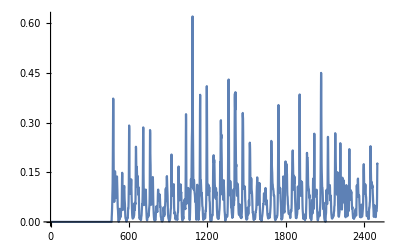

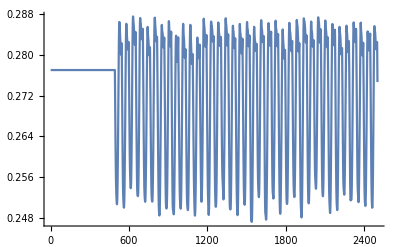

Sub03_(6)hop2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572832.0.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572833.0.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572834.0.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572835.0.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572836.0.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572837.0.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572838.0.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.242572839.0.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728310.0.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728311.0.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728312.0.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728313.0.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728314.0.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728315.0.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728316.0.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728317.0.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728318.0.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728319.0.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728320.0.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728321.0.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728322.0.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728323.0.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728324.0.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728325.0.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728326.0.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728327.0.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728328.0.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728329.0.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728330.0.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728331.0.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728332.0.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728333.0.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728334.0.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728335.0.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728336.0.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728337.0.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728338.0.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728339.0.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728340.0.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728341.0.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728342.0.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728343.0.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728344.0.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728345.0.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728346.0.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728347.0.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728348.0.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728349.0.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728350.0.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728351.0.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728352.0.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728353.0.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728354.0.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728355.0.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728356.0.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728357.0.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728358.0.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728359.0.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728360.0.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728361.0.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728362.0.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728363.0.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728364.0.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728365.0.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728366.0.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728367.0.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728368.0.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728369.0.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728370.0.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728371.0.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728372.0.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728373.0.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728374.0.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728375.0.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728376.0.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728377.0.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728378.0.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728379.0.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728380.0.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728381.0.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728382.0.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728383.0.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728384.0.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728385.0.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728386.0.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728387.0.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728388.0.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728389.0.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728390.0.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728391.0.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728392.0.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728393.0.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728394.0.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728395.0.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728396.0.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728397.0.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728398.0.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.2425728399.0.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283100.0.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283101.1.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283102.1.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283103.1.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283104.1.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283105.1.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283106.1.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283107.1.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283108.1.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283109.1.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283110.1.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283111.1.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283112.1.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283113.1.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283114.1.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283115.1.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283116.1.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283117.1.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283118.1.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283119.1.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283120.1.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283121.1.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283122.1.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283123.1.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283124.1.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283125.1.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283126.1.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283127.1.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283128.1.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283129.1.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283130.1.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283131.1.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283132.1.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283133.1.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283134.1.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283135.1.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283136.1.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283137.1.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283138.1.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283139.1.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283140.1.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283141.1.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283142.1.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283143.1.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283144.1.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283145.1.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283146.1.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283147.1.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283148.1.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283149.1.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283150.1.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283151.1.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283152.1.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283153.1.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283154.1.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283155.1.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283156.1.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283157.1.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283158.1.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283159.1.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283160.1.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283161.1.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283162.1.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283163.1.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283164.1.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283165.1.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283166.1.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283167.1.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283168.1.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283169.1.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283170.1.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283171.1.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283172.1.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283173.1.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283174.1.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283175.1.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283176.1.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283177.1.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283178.1.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283179.1.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283180.1.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283181.1.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283182.1.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283183.1.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283184.1.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283185.1.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283186.1.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283187.1.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283188.1.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283189.1.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283190.1.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283191.1.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283192.1.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283193.1.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283194.1.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283195.1.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283196.1.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283197.1.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283198.1.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283199.1.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283200.1.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283201.2.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283202.2.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283203.2.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283204.2.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283205.2.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283206.2.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283207.2.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283208.2.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283209.2.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283210.2.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283211.2.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283212.2.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283213.2.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283214.2.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283215.2.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283216.2.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283217.2.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283218.2.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283219.2.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283220.2.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283221.2.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283222.2.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283223.2.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283224.2.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283225.2.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283226.2.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283227.2.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283228.2.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283229.2.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283230.2.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283231.2.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283232.2.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283233.2.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283234.2.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283235.2.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283236.2.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283237.2.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283238.2.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283239.2.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283240.2.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283241.2.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283242.2.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283243.2.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283244.2.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283245.2.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283246.2.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283247.2.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283248.2.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283249.2.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283250.2.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283251.2.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283252.2.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283253.2.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283254.2.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283255.2.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283256.2.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283257.2.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283258.2.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283259.2.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283260.2.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283261.2.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283262.2.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283263.2.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283264.2.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283265.2.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283266.2.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283267.2.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283268.2.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283269.2.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283270.2.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283271.2.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283272.2.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283273.2.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283274.2.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283275.2.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283276.2.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283277.2.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283278.2.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283279.2.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283280.2.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283281.2.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283282.2.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283283.2.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283284.2.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283285.2.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283286.2.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283287.2.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283288.2.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283289.2.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283290.2.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283291.2.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283292.2.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283293.2.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283294.2.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283295.2.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283296.2.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283297.2.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283298.2.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283299.2.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283300.2.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283301.3.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283302.3.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283303.3.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283304.3.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283305.3.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283306.3.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283307.3.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283308.3.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283309.3.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283310.3.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283311.3.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283312.3.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283313.3.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283314.3.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283315.3.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283316.3.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283317.3.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283318.3.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283319.3.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283320.3.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283321.3.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283322.3.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283323.3.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283324.3.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283325.3.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283326.3.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283327.3.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283328.3.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283329.3.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283330.3.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283331.3.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283332.3.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283333.3.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283334.3.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283335.3.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283336.3.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283337.3.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283338.3.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283339.3.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283340.3.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283341.3.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283342.3.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283343.3.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283344.3.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283345.3.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283346.3.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283347.3.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283348.3.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283349.3.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283350.3.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283351.3.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283352.3.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283353.3.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283354.3.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283355.3.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283356.3.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283357.3.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283358.3.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283359.3.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283360.3.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283361.3.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283362.3.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283363.3.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283364.3.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283365.3.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283366.3.6500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283367.3.6600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283368.3.6700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283369.3.6800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283370.3.6900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283371.3.700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283372.3.7100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283373.3.7200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283374.3.7300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283375.3.7400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283376.3.7500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283377.3.7600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283378.3.7700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283379.3.7800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283380.3.7900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283381.3.800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283382.3.8100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283383.3.8200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283384.3.8300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283385.3.8400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283386.3.8500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283387.3.8600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283388.3.8700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283389.3.8800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283390.3.8900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283391.3.900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283392.3.9100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283393.3.9200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283394.3.9300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283395.3.9400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283396.3.9500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283397.3.9600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283398.3.9700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283399.3.9800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283400.3.9900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283401.4.00.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283402.4.0100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283403.4.0200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283404.4.0300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283405.4.0400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283406.4.0500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283407.4.0600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283408.4.0700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283409.4.0800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283410.4.0900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283411.4.100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283412.4.1100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283413.4.1200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283414.4.1300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283415.4.1400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283416.4.1500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283417.4.1600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283418.4.1700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283419.4.1800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283420.4.1900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283421.4.200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283422.4.2100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283423.4.2200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283424.4.2300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283425.4.2400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283426.4.2500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283427.4.2600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283428.4.2700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283429.4.2800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283430.4.2900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283431.4.300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283432.4.3100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283433.4.3200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.3987034300.4258793200.24257283434.4.3300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00324681847277878560.4258793200.24257283435.4.3400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00361806095643682660.4258793200.24257283436.4.3500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00360161117255882160.4258793200.24257283437.4.3600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00373330539332783440.4258793200.24257283438.4.3700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0040029013987317440.4258793200.24257283439.4.3800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0041963562529942390.4258793200.24257283440.4.3900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0049741391906571210.4258793200.24257283441.4.400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.00651558973485112740.4258793200.24257283442.4.4100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0077537511681540960.4258793200.24257283443.4.4200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0088242684887702950.4258793200.24257283444.4.4300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0108301565387624260.4258793200.24257283445.4.4400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0146814084477065350.4258793200.24257283446.4.4500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0200303136683166220.4258793200.24257283447.4.4600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0256170014074185960.4258793200.24257283448.4.4700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0296404183892441840.4258793200.24257283449.4.4800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.031529837333179610.4258793200.24257283450.4.4900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.031459033894152630.4258793200.24257283451.4.500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0292795082702969160.4258793200.24257283452.4.5100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.02582316991704520.4258793200.24257283453.4.5200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0232887633721243320.4258793200.24257283454.4.5300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0242797881620021830.4258793200.24257283455.4.5400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.02628762034368680.4258793200.24257283456.4.5500.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.025398590792388740.4258793200.24257283457.4.5600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.0247495468471111350.4258793200.24257283458.4.5700.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.029004352040606860.4258793200.24257283459.4.5800.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.039154105953113740.4258793200.24257283460.4.5900.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.054981162147041630.4258793200.24257283461.4.600.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.075080506047479250.4258793200.24257283462.4.6100.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.097752316774580470.4258793200.24257283463.4.6200.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.122159118311300610.4258793200.24257283464.4.6300.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.147133825149356250.4258793200.24257283465.4.6400.2770448700.3676724200.381725400.2669209900.3088851500.5122102400.2832566100.398703430.169854118788423960.425879320.0085372397418548870.24257283466.4.6500.2770448700.3676724200.381725400.2669209900.3088851500.512210240.0084749936401568030.2832566100.398703430.184917270775418470.425879320.0096247519936379570.24257283467.4.6600.2770448700.3676724200.381725400.266920990.0027725435751392040.308885150.00637013521537209150.512210240.0089261610493494430.2832566100.398703430.186011058888807670.425879320.0089190604115571250.24257283468.4.670.0154721627515871360.2770448700.3676724200.381725400.266920990.0032356481606416310.308885150.0081409794829050280.512210240.0088438549843172110.2832566100.398703430.171004136793932250.425879320.0094029954141293720.24257283469.4.680.0228249846003918120.2770448700.3676724200.381725400.266920990.0033774227124030940.308885150.011246892682005240.512210240.0089114514506169460.2832566100.398703430.144011194164751920.425879320.0132527384511935860.24257283470.4.690.033130447271677830.2770448700.3676724200.381725400.266920990.0050205495119607140.308885150.0170442213045211460.512210240.0089992832821292680.2832566100.398703430.111879625050619450.425879320.019932480573632710.24257283471.4.70.045032496221912670.2770448700.3676724200.381725400.266920990.009040836552817340.308885150.023793538858147970.512210240.0123256633414452930.2832566100.398703430.080607435133662660.425879320.0295250427176412950.24257283472.4.710.061028169296919380.2770448700.3676724200.381725400.266920990.0147363120320912550.308885150.027715167139874150.512210240.018090608695494390.2832566100.398703430.0540240082351010060.425879320.0426439055647506860.24257283473.4.720.08088107537088990.2770448700.3676724200.381725400.266920990.022236114585644970.308885150.0275172376008116950.512210240.0245161936953669950.283256610.0044983355238156230.398703430.033792027502845190.425879320.057223856559727310.24257283474.4.730.095580093542206090.2770448700.3676724200.38172540.00297718709514456850.266920990.0305124262578198930.308885150.0252032034663096230.512210240.027525186745050370.283256610.0053736057611798660.398703430.0200066744251001760.425879320.068501804227099560.24257283475.4.740.116753763537081670.2770448700.367672420.0119675742158238150.38172540.0046874658278237050.266920990.0344460631689469040.308885150.0214557427415376160.512210240.026916640192577490.283256610.008113639800968810.398703430.0126141395619199480.425879320.073039227256567110.24257283476.4.750.169226904643106050.277044870.0128235660500716290.367672420.0130815799622147310.38172540.0069761811632765510.266920990.030241907271710040.308885150.017192349879167560.512210240.023893215727878630.283256610.0143184512526682780.398703430.0128886154335405460.425879320.070812696019051090.24257283477.4.760.23223763231064120.277044870.016783795481932810.367672420.0175116769754516360.38172540.009983438768153420.266920990.0217257888627313370.308885150.0146294004017869460.512210240.018916797573834390.283256610.024728426717366050.398703430.019384577910982530.425879320.064206287109873830.24257283478.4.770.3036522822326760.277044870.0245754051998265940.367672420.034234742644036370.38172540.0137232567427963990.266920990.014593407482742760.308885150.0140995739736855040.512210240.0137941948162937090.283256610.038255510469945070.398703430.0270090498883373730.425879320.0571294390818748860.24257283479.4.780.37246387883733320.277044870.042623618171831250.367672420.067627118725136270.38172540.0182911648322747650.266920990.010667259357285830.308885150.0141017050846175080.512210240.0124971383086275590.283256610.050628609395673760.398703430.032935947711431310.425879320.053971166152374730.24257283480.4.790.370604776763540370.277044870.066553847090103410.367672420.120179703929618910.38172540.023128392319292390.266920990.0110669946503165090.308885150.0127731084214718940.512210240.016101033267564370.283256610.054955056485746040.398703430.0367851271431367950.425879320.0563657534385889960.24257283481.4.80.30935596899528080.277044870.099883307054095480.367672420.196884731271443620.38172540.0257993081951880150.266920990.016468280174493480.308885150.0111118707047959120.512210240.0213534603614236870.283256610.049225666840738990.398703430.0408147353043178050.425879320.063197623958527150.24257283482.4.810.231907217174096850.277044870.155333677666665840.367672420.287165491595452570.38172540.028104028378508490.266920990.0272960515208337840.308885150.0106887968314773820.512210240.0244757865529540330.283256610.04036164163323910.398703430.0481822678515377650.425879320.071108907108311260.24257283483.4.820.153315705542325150.277044870.208295228718954980.367672420.35868648364836690.38172540.033995133766488730.266920990.042675453877587330.308885150.010943849518987350.512210240.0265911802155908740.283256610.0326208344783079850.398703430.057289036005251430.425879320.078475711654121290.24257283484.4.830.108184063806945240.277044870.21077637609544850.367672420.39166191485254510.38172540.0367945175053956060.266920990.057777638917808240.308885150.0111718923485617650.512210240.0308249492378104670.283256610.0263899269539641970.398703430.059525283291751210.425879320.086286176048073430.24257283485.4.840.089205694734029210.277044870.193525531681685820.367672420.49207651354203650.38172540.0399031154964031160.266920990.06693424052622520.308885150.0104082106871594520.512210240.033996728154144710.283256610.0226614353762432770.398703430.047363907545157590.425879320.092799889278122050.24257283486.4.850.0698350677947020.277044870.21570102723436970.367672420.64811551596412890.38172540.053585260127555050.266920990.065672448965820350.308885150.0092734464528901870.512210240.032819469669774920.283256610.0252800369212344760.398703430.031778686753243610.425879320.09611745078713120.24257283487.4.860.0604936277122115760.277044870.25687371387579860.367672420.77551136437801590.38172540.06862818842564470.266920990.0558615451944034160.308885150.0101221302117538490.512210240.031713342032933160.283256610.031680133757725540.398703430.023531031473530210.425879320.099089029725836180.24257283488.4.870.0624248941765997360.277044870.25450083357130440.367672420.75790165727475320.38172540.074999599553616890.266920990.0539208881858573850.308885150.0147379604343546920.512210240.036169310386939590.283256610.033269745730364060.398703430.0193962990712632440.425879320.107336984156890930.24257283489.4.880.071124144651706550.277044870.20805232175831260.367672420.55344048355411410.38172540.071904801468971070.266920990.074186397627560460.308885150.023776088915418760.512210240.048246627010521780.283256610.033279857527461460.398703430.0145611542757759560.425879320.124169872247921310.24257283490.4.890.082921795831140790.277044870.186666724509475020.367672420.31801214256813390.38172540.067103351522067230.266920990.111873330626054260.308885150.039585218174590640.512210240.064187898258172120.283256610.0340602756264418440.398703430.0096043589423309360.425879320.152124119736369250.24257283491.4.90.097453881142249660.277044870.151596518608883240.367672420.163600807652247940.38172540.071177039715259590.266920990.160907488887308440.308885150.065283276432122770.512210240.070146948753957840.283256610.030269515858352560.398703430.006297536764567240.425879320.194222059314287350.24257283492.4.910.125334502195813130.277044870.14745662068786110.367672420.098256768042654030.38172540.102781517684628970.266920990.218232648482216130.308885150.105722712956711980.512210240.07126831125895710.283256610.021600008857082460.398703430.0053358923520513550.425879320.245565959047110120.24257283493.4.920.152954693941865750.274273950.198786124700649630.369772790.104946600171805750.383796330.173076098925777130.270112850.27616840642780670.308885150.15579260012418810.512210240.087541756636571460.283256610.0159604516987939470.398703430.0063199073678917530.425879320.29236871967862910.24257283494.4.930.146857766708250240.271184060.238713188305787530.372256660.15009861203597590.386230380.26132321894309930.273528840.309624367779655960.310668440.184994120879886310.51383230.109193773233243780.284924270.0143990451183289330.398703430.0071937978932746280.424207330.321734092162674070.24257283495.4.940.123605119761976740.268321990.235673664442964340.374407820.166794750703983030.388334090.314892154075746330.27655940.29426187635138150.312343750.17127241775727850.515414840.108531217218780160.286495510.0139915361373293810.397568380.0067409701487616720.422460610.32954111178370270.24270146496.4.950.102273237777422850.265480840.22738919839560420.376394490.148050425891315980.390270540.319099139214188640.279442390.2520488790747230.314023870.144219508602431320.516938970.097109494663278490.288075550.01431700551902320.396485640.0059580131225354570.420746160.32192896211823580.24290131497.4.960.089226335273661390.262727980.217094026154935480.378132910.164924170890475260.391954950.306774784227774270.282118320.245582597210266930.315728050.148429878361899720.518408150.120960108712039190.289683010.01636701693036750.395491010.0063100744522718660.419082030.31340056897753810.24324438498.4.970.079801932824835510.260236610.187649493639142460.37952310.222972128102238070.393288280.28402649585792090.284441990.29719460011833680.317368370.18552308399916310.519668650.188898978292458140.291236120.0203248257321646570.394738310.0076052100231159870.417676970.316724410721056670.24373568499.4.980.072695383487106470.25802980.20783634316545280.380548070.27817214948961460.394251420.28392654515019870.286423740.37182283825122790.318986970.253963147474905170.520818990.283430598760334550.292775880.026259334579805280.394144690.0100916925582924320.416419390.33101549326313290.24439141500.4.990.072525321109951930.25621270.230670635405493150.3811180.28411310523135640.394752520.302177366976845330.288002410.4268068955240660.320617350.32116884067555680.521917440.35197517196387250.294335610.031649655277996750.393666070.0128609336945380330.415245930.34579095127225140.24523455501.5.0.07829486921858920.254808720.28375298646623390.381274950.29811772176733470.394833540.31246206088927910.289189820.4316253806006220.322207010.34121214720121810.522953280.34419956075568310.295865390.0362256170550133150.393269480.0133155356983239060.414156960.35613087095271350.24615646502.5.010.081640806332733270.253704520.367997464594275850.381221520.36007197430840290.394701460.346352462224586270.290104130.40546592557989060.323642620.331833343639550970.523933620.32434274645935130.297254370.045023933866792510.392857570.012593358025477190.413104880.36991993495920350.24696729503.5.020.08526168457361040.252810340.409950528145135830.381128260.41706269355767480.394534820.420351066281326850.290832060.39258160460833350.324824580.334924357854490150.524836660.35403773609688220.298403170.064218109981300980.392382240.0135984897220353780.412082160.393963798201522050.24757947504.5.030.087383948173207880.252087690.410522481735995650.381099980.437038945649615040.39444740.497869587399104140.291412270.39724318639215960.325685460.342714580121354860.525669170.373103793696865640.299242820.09945805651293940.391798610.015757575603173720.411072780.419405016986706850.24789644505.5.040.083980779044713650.251507280.41067608282445230.381189520.5104452788871540.394497710.5667694530604870.29187310.405755433441268960.326216710.346233263982508530.526420520.358600964147176960.299762220.156953837328879550.391125790.0179850410338914180.410103980.4302030519935050.24791386506.5.050.096746535737133560.251109610.423167062496146550.381366640.69580133924982460.39465830.60304447140091640.292186180.41544587223514150.326430850.3440452938275670.527030520.35025959738083430.299971870.23910051345436580.390448570.0207719701062557970.409269520.41855429230225450.24768702507.5.060.12464848638009320.250768460.44870952144253510.381719210.84847419167103180.395015530.57016436232230420.292453060.42127617383911980.32636550.31736626546832810.52748960.361214452355516470.299907870.3401050137252710.389796960.02467598154274080.408600560.38901142320272440.24719776508.5.070.1371763690950740.250684050.4826225521671010.382030440.82892479690408840.395348480.5000029664051830.292518860.401860479280362950.326071660.25971763091433340.527736420.34979497915351130.299620320.44289725821902250.389291160.0285050270416138740.408194730.35305726626247280.2465946509.5.080.125701381984962560.250904810.488080316066956340.382228760.74471980791408990.395581850.42754493094882670.292346580.341457125906657060.325580390.191290737984017940.527753960.306177665154613640.299140220.52118027656958440.388972780.0303794239481353920.408081230.319056206166194230.24592823510.5.090.110844689229959770.251472670.51134323275752460.382247360.69319367072286050.395645210.413447109519074760.291900430.259619473032930870.324918360.140243007399479450.527518880.241932850105732650.298494520.53964109535164630.388890030.0290718660856148430.40829360.286317532976313240.24527408511.5.10.096284698449472070.252447670.55335746180057110.382035540.58770656474005460.39548760.45116582029088820.291124140.186103505065872950.324064710.10976871524006590.527065280.170163721041478640.297664080.47950612578119790.388956870.0244794612656655950.408764550.248630331242179370.24451468512.5.110.077894729400806650.253811510.5146012222344020.381573480.458314833214344740.395086330.463878895673088760.290016290.131194360838417260.323041080.0867319160968950.526351620.113303612247055260.296671530.379825852312679730.389259540.0184040734403848150.409559960.203138461789885370.2437733513.5.120.056800666902408130.255566820.412268131392088230.380841710.32417115738421420.394421250.41580289265078360.288552140.090016061117897590.321838840.064412041370313120.525427460.072639371942530150.295510310.279094138818172740.389719220.0127930638658845120.410598050.152587915457374820.2430072514.5.130.043576886032206390.257683660.32680615589735040.379836350.245325118764635220.393486990.34305109827058850.286728130.056795545014100780.320463790.0437187934288411140.524346920.0447117046478421740.294188310.2042202331586240.390269080.00874437490727070.411800150.10356230104321790.24219984515.5.140.038680259755049770.260105230.294035311434823640.378568360.236866545273497990.392292440.286237339515400650.284561980.032368112184807710.318936950.026981044542841770.523159830.0275777614210587740.292728170.170727910063044860.390865450.0069981519894385170.413106460.06364694404267540.24134823516.5.150.033984468410916050.262766350.27272739243689820.377057920.222597014302433870.390855430.247592102097818570.28208180.0171357665596445980.317274110.015235192800057460.521882920.0176046903326666370.291146690.155481301815248830.391507720.0071933695893294640.414495070.037878954457206190.24050426517.5.160.0240368006958487650.265611480.19489475647811380.375325320.169853825374557340.389194010.196310765989102520.279312540.0089007542371936310.315471890.0082344702935554060.520494740.0106180342915011450.289441020.136285600562360080.392215880.0083487060566333030.415972970.0241861324097796780.23971679518.5.170.0133635232141355990.268641750.116777064931457180.373337070.112931760256710840.387273540.135089366011150150.276227140.0059328173671798810.31352210.004537586822353880.518988420.00747041250713640840.287603220.099046761563066550.392982020.0103000382131327030.417519820.0154395673823252870.2390021519.5.180.0052063709733434380.271743760.07023112840086530.37116430.073942413975110140.385162110.08100010791143760.272921220.0053049776680750570.311460430.00255398469173294740.517274450.0078370770625502040.285666520.058604077058808560.393961880.0130311904044019610.419258880.0104970884883873630.23857681520.5.190.00174854125685186960.274917270.042227791698125370.368803510.0524383729667062260.382855640.042406579802263340.269382660.0049216051291355470.309284390.00158535664229992850.51545240.008645866015371570.283629520.0309141421619130480.394999020.0157033698146761750.421040680.0119462487413957640.23825233521.5.20.00065455620826873750.278049320.0266876624524056520.366370290.0400096910072593940.380465990.0224699716286173540.265733820.0042490219672173180.307028440.0017238898878104610.513505650.0070383387594370120.281525710.0143220810292575720.3961490.017552737988723110.422912940.0176636278357342160.23805633522.5.212.896523095501155e-60.280956280.0176386332405833670.364081550.032412313588187890.378202220.0129126914527053080.262207620.0042602128203580740.30473570.00226443542920900420.511532190.0063485836942609750.279395390.0076805883230110330.397296290.018822374961342250.424745920.0303376230431011940.23789248523.5.220.00195453170701161830.283243420.0124087906070319950.362390650.0290202284621841750.376020660.0082549776725247340.259339270.004174168408570450.302546940.00245440849725777140.509630740.007370322636471820.277364030.0087294722817759730.398385810.0201280795925188740.426453180.0543505987411970340.23772932524.5.230.0069947664356433960.284877140.0104211193581748960.361340530.0275276897843947550.374458770.0063400861874313540.25724030.0042971842818453640.300570230.00195957762568305540.507901360.0072547192937406920.275525130.0123130152906770430.399364440.0217499782857545070.427954170.088531616073307690.23757063525.5.240.0107946803407191330.285976280.010018726171428250.360753440.0253010887269943670.37343020.00648569336606325850.255804990.004937296764585210.29894320.00176698644072052940.506451290.0058360760764366070.274004170.019924641929593070.400175950.0235356672795790440.429179910.127750254171217710.23740357526.5.250.008786198854179160.286487330.0088933149276437390.360672160.0202219312545140330.373008580.00766477566033347750.255131390.0057863296609667720.297773090.0027570385109105740.505376190.0052865514580602830.272904240.0319397713552583840.40074210.0247267462269776150.43006640.163859597512926720.23713197527.5.260.0072985334762190530.286378480.007467585665872030.361160890.0142409526802751650.373256560.0086455461251207720.25527520.0061207384916433160.297045130.00372287514079156030.504672510.007972746562149420.272216790.0386550286152351140.401049430.021841041536771910.43062090.187373446485920830.23668759528.5.270.0131140892483021450.285838840.0074268152509755810.361977450.0099133727268170930.373964110.0095442840458736070.255985470.005742405556114110.296696640.0054372139643244840.504289750.012490327811224090.271886740.032431711994514580.401156630.016956151396919790.430908920.19008085101682860.23614831529.5.280.0267272964531657530.285190160.0082516070852466350.362833920.0072693915456868580.374767040.0101665644865310060.256833420.0053590368522181570.296572070.0085872797435646960.504097760.0155379058652093240.271768590.0202418559451506970.4011850.0115340040088075420.431059980.169984179291351870.23568405530.5.290.039602833542200520.284656610.0075394792447482910.363511120.0041634685032605850.375411830.011171661070443780.257526030.004855047495471030.296561160.0106416670807682380.5039920.0145561864134602080.271758240.010809911747754870.401217260.0066886882158070160.431169910.134207193055678330.23537153531.5.30.039168622181633820.284412550.0084501222319425750.363830830.0022688929290013060.375712330.0113115457784890880.25784140.0038316508430356290.29651740.008967725543803590.503794550.0118267761559730250.271716710.008903697035191920.401429470.0054379418805275820.431430510.094737675513403730.23536386532.5.310.028218319815969310.283863670.0160942205798366330.364432790.00525571833316350840.376321690.0102967373267664980.258547260.0032124455706805470.296840960.0053107424914541390.504017010.0089378203523910130.27202350.008849785636782930.401347490.0073385497539096930.43129410.061774912962024910.23536108533.5.320.017413710031769390.28331370.0259120242272622080.364961670.0127983771743101460.376930160.009600285791374750.259249830.00367086548727437860.297170790.00228391802143909770.504174180.0066438467694246920.272335650.0054084262708781080.401409150.0105449270156611660.431278480.041256726068845940.23557853534.5.330.0136881795326352030.282637480.0276203586617368960.365589050.0216301076652805170.377667110.0105339710254928570.260107210.0040962593502229140.297615120.00117033685493415070.504416910.006371420924882380.272755280.0042324272027289350.401452610.0138580818493666370.431208930.037852597328607830.23587543535.5.340.0153463109433227190.281930270.026582452162729260.366198460.0343818985433678450.378418430.0125717389672453260.260996190.00336573831305135570.298165070.0011229204401761840.504724410.0067792889978436950.273273370.0071055698589755680.401490310.014730551085895140.431104340.0514946503388242350.23624089536.5.350.018484285647977380.281334230.046237397337645040.366640450.063124341571430560.379023750.015297299479356630.261739320.00217653338495581030.298765690.00190154464459633770.50505010.0050071841904181050.273837670.008120614337182980.401549520.014957637314109350.431001460.073667882596557630.2366833537.5.360.0206776768216633370.28086410.098114786628985650.366903330.126225792335959120.379466590.020219981957387990.262321490.00262659048842510750.299406110.00327178034425139060.505397340.00310377196140133520.27443780.0091968902806358180.401619750.0199822333447137040.430890480.098034717296546740.23719017538.5.370.0237373737780130350.280485670.182495213743509550.367042880.224796559161948880.379792150.0302601559234724760.262787580.0047348229849189230.300060370.003971239910972160.505747130.0055393915748680110.275049410.0162073792663716030.401704980.0310515359092622120.43078070.122535125188271050.23775859539.5.380.03120914929905010.280170630.25284207336605210.367091650.31330035098133010.380034550.040784599463026760.263173860.0079556739962953410.300733830.0045464666670779010.506100750.0110650727236334730.275677630.0254939361747832240.401806580.041536020014842190.430671750.146079080015060950.23838318540.5.390.0372507805240996150.280051360.251533748860773230.366900070.349026182291949870.380042080.046004312170764380.263319690.013013922923210730.301404730.0066091119167334190.506455310.0164919740819881620.276302350.0338247375184872260.401901250.0449247377301213860.430549480.167925329389748720.2390149541.5.40.037520828304119830.280320160.243925415597824190.36624720.336975569379626250.379594480.046906585062412660.262990710.020052828232887480.302048570.0108330063530282190.506803210.0232756315206043840.276901040.038287175252065170.401982080.0405321660947217250.430412380.18701112106054720.23964085542.5.410.035218944693833560.280909560.26601893647524850.365223510.31933493750494890.378774560.041810107518917390.262265360.0279906020002147380.302644640.016254306986595590.507135370.031475467863594520.277454750.035014553760692230.402019810.032250948624531210.430252690.199902518551247850.24015899543.5.420.035631479250606590.281623940.23131286065112110.364043830.308217207646801660.377800280.039953746727175390.261378810.035296922236421990.303234080.021106623317457290.507478810.037867213308357190.278001960.0271192775604072350.402024780.0221256050375578420.430060080.2050782939536630.24064382544.5.430.041868857431837870.282314150.16215758223795950.362895680.25651013095160010.376851650.038262057407665230.260514610.040945978303106460.303806840.02520134562562720.507823940.040664439006418920.278533470.0203820821382616830.402006680.0139052678326184660.429847890.20722840817433080.2410914545.5.440.062301677751587310.28056830.107307858586221190.364475510.174612349088629380.378586570.0372662426699318160.2626860.0426934332965387060.304888180.030619677549148410.508772810.040880799257636130.27953690.0171841586456210440.40146670.0087256266631660730.428993040.216248130780653470.24116587546.5.450.098078038095341260.276849420.073756478645332720.367884810.14071226906167660.381932210.051193689893226530.267150130.0411639357645403740.306864630.041600194024154760.510464510.041914330819671680.281373270.0217094480610218950.400530490.0064206677827345080.42745560.23922643122663990.24135827547.5.460.13158344265273110.273768130.069415238924618570.370222940.194070011558662520.384237050.074371793800664760.270682370.0437167226210193540.309117790.063516574594152680.512308960.0482815410021610740.283473880.031188103451123370.399579340.0060545896224643790.425756790.27204559053295440.24183021548.5.470.148286374414227540.270627260.116408654211568170.37267790.283517485995552270.386642720.120559982491751870.274128430.056833451105591640.311007630.090880317686377050.514060240.061089036013281470.285242040.03513061971035460.398472020.0061863556518546520.423978990.30394967868746650.24201226549.5.480.13686138418854310.26736050.203169310528194650.375199930.33002010013744230.389109050.209878476819384120.277548950.081004499021212530.312742830.115919287941872420.515597830.078841257317396830.286870440.032130248086007480.397510970.0066338993387302890.422387460.3273162413840550.24221698550.5.490.093412475241118810.264258590.272587418451604560.377406190.307979764712662030.391261110.31664943997478830.280644640.118944378487514520.314433090.150860333682777760.517073680.11152131145626410.288461060.0330004725729162040.396557080.0083873526596191130.420799340.33974681756872230.24242837551.5.50.058778203421025090.26122370.274225477411873030.379379530.267950267498076270.393177510.379989365352795650.283532390.173655568134503860.31612990.203434864544769140.518438540.173071352219340860.29006290.041538614698984410.395735910.0115179058963035350.419316060.340112348590061560.24282184552.5.510.040167858999200280.258491840.20941338174360460.380877220.215116809962290770.394614480.33579095031761720.286014710.244789645334175130.317873040.25645220664842310.519660050.27090878351423710.291715370.0505504223435940540.395128620.0144483788631924160.418007190.32670118483349030.24350097553.5.520.035997638884778690.256159660.15995588971084620.381814540.205641043265802820.395481810.2597296495032650.288047780.33980759781867030.319705780.30517782728038520.520843020.382348489840946550.293462380.056069195006520890.394638070.016148292899891660.416749450.301763013370388860.24446061554.5.530.0488469504838230860.254330520.211534391186706170.382122240.28037697157845250.395704430.303825222028455850.289587880.480468851960922540.321645750.36026712050056050.521976550.45765594711533230.295324270.06331403433603780.394308180.0172438878415450660.415588890.27630114879002050.24571218555.5.540.066722959521617140.2530420.31203217530382590.381900180.3426258745886890.395383830.41596133498080640.290644540.66803764581394390.323536940.396609071306731840.522970840.48382293553309080.297151890.077114455926997130.394149110.018102110696297490.414610010.2635429394058050.24709085556.5.550.0805595085186190.252200170.40047308371517770.3813880.428009741890044040.394769180.499116526088837940.291322440.8532002775276520.325192680.403930533222452150.52382090.482249457581525650.298761890.100158944680828340.394033040.0189597224888019450.413760210.264365374480129640.24833726557.5.560.085763662182796460.251547050.444558725993194850.380938890.55118943163404840.39422720.5441622942221340.291841670.96177633124559190.326482330.42153347782972810.524531940.489322137487294250.300022290.13900501187962070.393854990.02037635056863340.412999690.26856016317730960.24923212558.5.570.087128689184585090.250993370.497078134222084630.38070380.59819051044701020.39392160.58143739575185630.292277290.96020479260219520.327356920.471633159414860450.525123180.54768848780673650.300880420.194533029782523650.393586290.0226427498963461160.412316990.267419459644624660.24973349559.5.580.089818661638653930.250540430.52092750235110570.380716880.54249012872157180.393895440.61418954411784740.292630580.88791251892616660.32781060.52595650026791020.525616420.59226720084174910.301326730.26007721530990960.3932080.0256873866547565470.411700120.25941743453567750.24982886560.5.590.094241710431246070.250187010.53471128890925980.380946710.5170089313270490.394117060.64894791465858690.292904320.79706386699136930.327902240.53094424189620990.526022890.54754889388956670.301416980.327587746153682140.392737190.0286889456407345730.411149950.247617739026489040.2495666561.5.60.099396345105012550.250013980.54826261446863170.381261960.50624730284956390.394449290.63370565335383140.293037740.6923181366645780.327708790.462428269126698650.526285770.43904066856100990.30122650.39171008162421210.392281370.031244480488526270.410756850.233412758231782920.24905698562.5.610.103328826380143370.250111610.54158180977160920.381526840.53140338689901170.394749420.54756844200906730.292962510.56446107198817050.327294180.36652921483838520.526335540.32694635918572920.300818760.431705151795147960.391966170.034226618180739380.410624350.21417774543968880.24844324563.5.620.108079651743716610.250566340.50084251536023490.381625030.61906067497110760.394895780.46533568705429470.292610440.431449907262365260.326697620.2834230194622410.526173250.23599862374796110.300233260.425828542650798670.391814070.0377451255206829040.410752650.1881963020304770.2477859564.5.630.10847928229184490.251395440.409719605918094530.381525750.65527920634237260.394855310.408843548273851050.291961370.3171638676544290.325921310.213766423950990380.52581390.163164353323050760.29947330.37319259362717760.391811890.0386973775234412950.411117380.15710782838073480.24709691565.5.640.093464992313052010.252665890.314559772463942570.381151870.52096212402963280.394549280.364222894441010970.290948620.227077807529977550.324961350.152291356074243770.525253530.108426290391291330.29853640.27823795523934740.391963670.037180241985379230.411716340.124764933665389470.24639791566.5.650.075068194740773340.254337260.258006697928440050.380534520.351109452025743950.394008780.325011280186539350.289582290.159391060295608460.323788660.103479477691185190.524493590.076274510314465930.297396070.17300464355222940.392246870.0414840206186835940.412537460.09426606655624340.24564315567.5.660.064822046592256930.256367140.23684389658432580.379685530.270701890801146870.393243730.27413104306422340.287870080.11065226203570530.322398530.076355072684877640.523549140.072731316504801020.296050290.092260221154379640.392638920.053892318055724020.413556750.067363084079023970.24481669568.5.670.059045471278847720.258680940.205874546812363250.378636670.2049983258429360.392282640.196814998038348450.285846420.074136309621838540.320802810.069215385475000530.5224710.090108930721207460.294513640.044374553299106540.393072490.072327248880478520.414702090.045106242955467550.243873569.5.680.052378561607906470.261223310.164070585196810250.377392210.130274532820023880.391125810.141594792221292230.283532750.0466665795434029270.319036120.063998335530487530.521290250.098674932578919820.292822770.0218538412737372960.393536080.096365224805427880.415943840.0275912140746306930.24284262570.5.690.038748195899851590.26395860.112599098551921630.375933990.07595926457430780.389751320.125480779822530110.280936260.028125973598190930.31713450.050676433720035650.52000450.079152340073057990.291014280.0135515277634504480.394060110.124234157907396310.417288680.0158222500089812740.24180397571.5.70.02534442412211060.266898680.070194313436904020.374219070.048563997031807210.388114460.102511795624694830.278019190.0162577548374830270.315081410.0329427444656967550.518599280.050902693575795810.289072420.0099382799730231250.394639560.153862027688813130.418717380.0113960683124233830.24079323572.5.710.017092568009927610.269939140.046322009380201080.372299560.035447835265619020.386263580.063546252573195710.274862740.009244074320861290.312905690.018422336395711120.516943670.0299828251367217880.28702350.0082839368914688020.395472310.17918056270355760.420391560.010699067921718610.24007483573.5.720.0125085591252300130.273134070.0333635109204836540.37010130.0305027216887496160.384125150.0352544239128677950.271390560.0063473350741188550.310593270.0102717782159114770.51513870.0172457721254701580.284853870.0071907704226393030.39639550.189904500190781620.422139650.0094710814732977180.23950955574.5.730.0105209675660873360.276338270.0247648572303342360.367771810.0283382256120444270.381842140.0202949687476684860.267746520.00568381701015809640.308166330.00715362940642588850.513188780.0109345643498375090.282585840.0075986519801348930.397422780.180888754859360850.423968930.0089166160227595830.23909271575.5.740.00924763634166690.279373580.0197178615244797370.365517820.026424957929580480.379613170.0125237235165464730.264144110.0052887320750093640.305658670.0060275646624787740.511147120.00743362212497671640.280252240.009026597361536370.398506650.156820509241328570.425823030.0094217922807087010.23875441576.5.750.0077883657957856080.281891680.0185680342854091760.363743610.0251747971178113840.377495230.0100354599320654460.261044480.0052192674497178940.303176450.004862562128247340.509062840.0042954574643365780.277948470.0100991121243972240.399646370.126833560336369170.427673180.00984694127511560.23851089577.5.760.008197881993039860.283760110.018321633254415270.362607860.0252060310509229360.375749870.0097007310391196160.258679920.00613535044387995740.300840310.0034201126514475540.507075330.00399901270367201450.275776850.0115391833021116240.400710980.100478128061981450.429368890.0094080282550433590.23822444578.5.770.0075729791090761110.285136090.0161439243011712380.361898480.02540755542831540.37447460.00852774804593550.25690380.0067895743881159070.298774950.00292424226594811430.505307260.0056922821461928730.273846360.0128248243081019850.401637310.084821618678036810.430815220.0084267143202280540.23794958579.5.780.00333170354702905240.286015520.0139666785091801680.361589750.0240626387171123180.373685490.0070507134981013790.255753410.0060450168726442840.297112040.0031550592016788760.503886680.0053419308157811760.272280090.0120043357161977430.402332860.074934161744818230.431927650.0074875362212826770.23763018580.5.790.00133359988736057950.286138570.0129317934103824320.361793410.023118931843064520.373711470.00774551213156878750.25559150.0046986819790151420.295963790.0028568152605387240.502912180.00262677144116738950.27119040.0086845530482585960.402735290.060609014779935710.432643390.00661048570735709140.23718976581.5.80.00095381031806506350.285574810.013167900584695750.362687040.022922729445027090.374486390.0090201492843807740.256331380.00422830146710239350.295302370.00218847355292017130.502350950.00211269848870650760.270559120.006521335942948780.402897980.043682003590740130.433021860.0052697381183198560.2366944582.5.810.0028286081438513410.284778030.0129236949631948770.363786990.0233391549697458160.375495160.0084664513382236070.25736880.00385739190911485450.294960250.00172444475623510330.502046360.0045959535146182010.270231440.0088076285328546680.402962670.030271560858922250.433224020.0066360821282580030.23629165583.5.820.0069700505864183710.284201880.0117075956710242010.3645640.0233438819499055570.376214160.006529904235837650.258112870.00273493497842036350.294769130.00125258359792737670.501866680.0053020775723932550.270048040.0117314339305173170.403001550.024820523829973250.433347610.0103592217909498720.23603018584.5.830.0090503741300820740.283871260.0115368466000215120.364995760.0228140004357236420.376619240.0057818165854848890.258537540.00250714524224285870.29470770.00144618160959446080.501811050.00338064181014649870.269989030.0125697561763141640.403027510.0292258333539820480.433397160.012047759350191850.23596218585.5.840.008260615885232410.283537520.0158267383626091160.365377620.0238076694595069150.377001010.006604056795536610.258964470.00336243467035330850.294847520.00215492367353182150.501893720.00353900074473711920.270123290.015841900213966680.40307150.039493548222814850.433395360.0117608765607265140.23611648586.5.850.0083931437423351260.283087380.0250085004995929780.365847610.033304809143570570.377492220.006569911590857920.259537570.00329668876889673740.295194820.0028362418946354820.502113660.0061941935035316890.270456190.022343983501899980.403114170.0472649161878831850.433335170.012957576825837460.23641753587.5.860.0103465209999421110.282577270.029219488734880550.366343340.048353257597551630.378027550.0062613357990233830.26018320.00217721386163448540.295717520.0029209932699481120.502457440.0058413070937734430.270955680.024533461408945590.403138310.044498230562062080.433208880.0155956602012851040.23682151588.5.870.0115493926060216360.282107290.0275267749061706180.36674790.067659255961458190.378489650.0094029637095672230.260774410.00169187649982097950.296380920.00315793166296908250.502909930.00249062741008783260.271587130.0192663736155100840.403127670.033763126632928140.433007940.0186827243355688030.23729773589.5.880.0116868212020719980.281681420.036279182933546030.366996210.091299480415783940.378877910.015449792584061770.261307130.0032920726808871240.29714890.00386854622809801670.503426670.0023552134090749990.272314960.0121896125927960420.403096830.0228826760160288430.432764620.0236364657147608540.23779373590.5.890.0112987999706539110.281405430.064709068537270880.366926490.117480109360899740.37906870.0198814958021908160.261650830.0052405186908950810.297997240.0054026178178420440.504024860.0058702566869645330.273115410.0082847739292687720.402991980.0141144478468889860.432428060.0334256786682061160.23826291591.5.90.0140536033295827550.28119550.134471029515092740.366744230.163968736021045220.379164220.02399031550528850.261911470.0070843681838289320.2989020.0067657813032052340.504632040.00737539936924422150.273965540.0080052092633993050.402904940.0082622256658498040.432097390.051187614415074090.23875816592.5.910.024383080119644590.281092770.243014485950052870.366396290.251662707108334550.379112620.039309261138423540.262038760.010444935426781880.299866210.0080811363641149580.505284080.0076222317466325950.274868050.009985309677091730.402795180.0060930388254403760.431723220.076964554125239820.23927813593.5.920.036474857646614570.281068870.30875246843696820.365923060.377226115395306260.378948780.068504031498579630.262068340.015166550989412440.300876420.0103615782530857830.505933530.0106052030916670150.27581050.0141899921985534780.402710330.0079619029347517620.431360720.107482545824274260.23982717594.5.930.040290284968425930.281126830.26236746051259610.365319690.44878072446386390.378667750.092113302849863660.261996580.0198216869037884550.30193310.0133500741257793350.506600110.0177282811568554920.276793720.0207445828234191850.402629350.0108322938777207240.430980960.13673144397260340.24039434595.5.940.040254874251558430.281391530.197047039774037760.364457350.483074154500821530.378130210.095549403573876330.261668110.0244730863486113080.302985980.0185796805398479660.507262640.0272896099542110670.277771670.0271876983840179140.402531960.0103089548651632760.430582240.157621987897054870.24090963596.5.950.045770156190988730.281883130.185016669734033020.3633310.51572255778880280.377321580.090643694015445250.261055170.0313707387457648960.30399360.026793641497339790.507893640.036098791594003650.278706770.029816239221014050.402445710.0069552321587784790.430195560.16602417334024270.24141592597.5.960.062523254675335950.282563990.177944013383257830.362012540.48770739749129750.376213170.074433952024611320.260199950.0415391562983362040.304903510.037239844099352230.508479310.0417355017754216240.279551130.031874752134141170.402348150.0041623819294351250.42981510.16299667756436560.24187048598.5.970.093557608010785050.282291070.14475431563492910.361861870.422503768464280840.376088720.0589025351003711960.260543630.055089452527092070.305824160.0451588615110492950.509242580.045949234957596660.280405950.0464938009282541840.402018680.003583631464515470.429182290.154841974853211470.24215287599.5.980.142979981193610880.279429880.107634223857051960.364587010.420441938725083950.378742910.064597713310499020.264075910.076077827557085980.307256350.052515127579033220.510548860.0516297662796852550.281737890.076296310913265410.401314860.0043883158075620730.427991690.151404337118938160.24242945600.5.990.218823589746118760.276362980.100686566026848330.367053990.451723578045200140.381154950.091363871929658860.267717780.11144274609557070.309392350.06865338231982380.512294220.0584096042449260560.283730410.114475003592445470.400430570.005496753424269170.426396520.161292570250665620.24282226601.6.0.29111232835992550.273641650.138927210650599460.369008840.50001049898190310.383058240.13623206435841870.270824140.162479516977820320.311466080.0985389129017470.514096090.070296787829832940.285671810.150362365876567980.399386920.0066616723481316670.424613990.18631058315014490.24312814602.6.010.27783796242201030.270548860.20283861367979890.371387780.57458142700617940.385366940.198565915410283040.274212470.220921209335137060.313291390.132298792633676640.515712810.092451414818490010.287386190.171258547419328830.398385960.0075597691233919740.422925670.224916990166925320.24338984603.6.020.19756578241886190.267700320.221983125372691960.373347360.53017656861949790.387258030.26617327234246560.277200850.272269604935270860.315103110.157073492239264030.517232430.13033849482057260.289092890.177256623806486520.397436370.008679673005368950.421271150.27310859272604820.24372622604.6.030.123171638700561980.264902570.23757773582288510.375066370.41559920297502020.388901510.3400954197691490.280014030.31296274715898890.316972860.18316440635425320.518671780.193284024956373670.290861020.194422060945345640.396564920.0105371891133798180.419653850.321502669584900760.24421722605.6.040.088351794440011550.262379310.36470043815044480.376341160.372123977889593840.390093810.40687819422802140.282449090.361872483932712150.318880340.229732340297155640.520171970.27057247025683410.292674190.226345659808512230.39561030.0129981919702198060.417912440.36218042359917160.24474003606.6.050.084444839982227380.260198330.58207960745685440.377171010.416776206504049230.390832770.448784765634184240.284476980.43409061494910480.320783010.30358440886777370.521470580.35864278172929970.294494630.24517574717726050.394933690.0155891627287250020.416450440.395342400314871830.2455181607.6.060.091166379028848170.25848310.75312070911455920.377481470.50198184435209360.391043330.493857201481795850.286022480.51645620868970890.322658210.41405291076634670.522661260.46758404527828370.296301180.24332554822845280.39440380.017825072964464770.415141560.421309022332197360.24643269608.6.070.098921981750585160.257163890.77968397616550920.377424110.54968058596839250.390878690.52060358709619290.287181970.57250966934301810.32441540.55481146106320050.523629070.53279624231753820.298004940.233610605126865660.394124360.019719446583531040.414133980.43458747883340080.24743033609.6.080.110727826271682550.256107850.7114404633287020.377255710.56350184193688070.39060520.56581532912702030.288092060.56476726235633610.325903410.65180981227984540.524350950.55754549111126580.29945580.23278479783005250.39401450.021053211213419760.41341360.434886691125652650.24829655610.6.090.119013464490272810.255233660.67980497154793510.37716070.54408232962463990.390420480.66127374213885190.288833380.50297221264700290.327019370.62589244999646070.524927960.5703303117769890.300548880.253991623468573740.393873960.021596753884759860.412810960.42953908693601250.24884863611.6.10.112077355011041660.254573940.65793096257694560.377166930.50788970365691450.390363330.77024478671786960.289385660.43860917862277840.327736250.51448754482082680.525366890.54553593281721390.301253530.309964198760973530.393682670.0228362638189352240.412321530.43109912374645120.24908105612.6.110.106130565005388770.254088480.58201324725205120.377338570.490965281916941330.390504490.80841696297157010.289788130.39043868919347670.32805530.392880594331017740.525742670.48173547284146560.30156780.39061929813437460.393366140.02673732158852180.41185430.44963701144640030.24900865613.6.120.104178311043930420.25384760.50939987084403910.377592250.50342894253946860.390760670.68745066216071490.289986620.340530871994508770.328015630.28644714524483840.525935410.390954984449256640.30152870.465513187868263350.393080650.032337105898920960.411580710.475737005522671950.24872212614.6.130.105649437731444720.253831360.486844565664827640.377902610.63786281086922270.391101330.58219918119409850.289999970.281177583584757140.32766940.206344319094586670.525923730.297549561847513740.301187730.5168006936072070.392878780.037262016668613950.41153420.48518147286293190.24830139615.6.140.108140257231404680.254097270.50690715871838230.378168530.72096747801810490.39141890.59299784454453370.289780880.21828858104022650.327064030.153341056969563160.525697360.219357678675823150.300592720.52376021748967250.392800140.040747310300518950.411736640.4596573379734220.2477817616.6.150.120347129066300850.254726050.52685579422224030.378276190.64256756187096850.391593990.54485696954240180.289258860.160026200969992180.326229320.114021897448682320.525273150.156623683751766160.299774570.460599232755559030.392849930.03629165259744220.41216930.398603319814530230.24719631617.6.160.12848504500349860.255793660.53626118727715890.378118950.57443638991769440.391515690.410946585354812430.288359750.11080148918426080.325182870.081654339804812040.524537320.106122209166046450.298752320.349505727599206450.393181970.025654498014919570.412984240.316934873702356960.24667453618.6.170.116345332211112350.257355220.492314238882875950.377649150.490236848871260730.391136560.29476255063108210.287015370.07212321892272060.323880760.0553852718615763240.523628990.067499083971662950.297485460.24519397555945980.393596820.0172968282334460820.41397310.233397382864957620.24607847619.6.180.096609216269970680.25926880.36993806771920090.376960590.35338774992697240.390545710.2359522132780110.285319880.043925390357684510.322331350.036430507621247560.522447610.040320869618834980.295985420.164501178368872240.394220690.0126406854617372830.415278620.160788331157510620.24545063620.6.190.076406444099798880.261530060.241174840945932780.376011980.239073449390880540.389697880.191486244044668160.283247130.0251741061111335940.320555590.025002925466821260.52113450.0228742777479156480.294276360.104881917702610930.394868120.0102260599840245470.416706910.104559365327642530.24463305621.6.20.0597395991597975340.264054220.18006004838822250.374823880.139438373216759420.388608160.17125341308791580.280843450.0148638981484927760.318605010.0190375525012386370.519706760.0155108504384810150.29241180.067142664279158270.395552660.008858278673952260.418248170.064973858080446150.24369708622.6.210.051270740082734370.266820860.14133106988134670.373358330.073734035091520710.387234960.145685028050748680.27809810.0098233959856329470.316511270.0180355630629553050.518200040.0136312913996122410.290423780.0423650547489934360.39624620.0076044158202037670.419840090.039048343971166320.24270896623.6.220.0378423218537241240.269871960.113116367121738480.371523710.042215154392018920.385485820.099271915913812580.274934040.0070928641730030750.314265530.0247933868656619040.516581990.0132370823407578650.288303170.0239241731877836530.39697370.0057182254552148640.421482690.023328624647543870.24175241624.6.230.025736612337412740.27306830.082039736634156080.369422080.0228338894530185420.383459180.06253661622284030.271463660.0066350890401366680.311871110.039119116859389630.514800560.012962148469814220.286051790.0128949486380775330.397797050.00381496893869395870.423210530.013417529854957230.24093831625.6.240.018552384067644190.276362160.048858315197582270.367090090.0098371220528260510.381189710.035897360808202860.267718740.007954644624016030.309330480.0585680717563345360.512802470.0141086103733324470.283672590.0099219340419173280.398788880.002604239336356990.425089160.0086291616253241850.24032909626.6.250.0146858855661186720.279653080.0271802051497911820.364648680.0043993374477567030.378792860.020709468763194740.263805020.0094021296686738610.306646790.075763478880788740.510625780.016233616640410460.28117060.0105955937990467150.399886960.00260106785331392370.427062790.0120357354026799680.23980564627.6.260.012233882484080350.282574160.0174211886268839830.362526710.00258628292157561450.376521210.0144509341386401670.260187130.0110048701334142590.303897220.080439452396678630.508363370.019664784279607770.278617340.0082623561256249670.401003820.00270036569806925230.429024660.019544848140144830.23925917628.6.270.0104713154493754090.2847870.0133443725022790150.361129140.00190684691882599660.374440130.0122190639515718430.257357180.0129168727040178570.301220060.077032903811544860.506157020.023043704932283850.276130490.0062524118484941230.402026060.0027392271784619760.430828670.0286924374699279730.23858043629.6.280.0099686685073536280.286391850.010088818904058540.360294170.0017113437684071080.372950940.0104344768588099330.255257540.0146474382605581380.298803080.07109042002981850.504187920.0256905866298910020.273872740.0102283264380309250.40285610.00301836007388215070.432318730.040385056161992850.23783947630.6.290.010666746826426930.287331860.0063529136978666740.360007440.00211785962019015070.372119470.0090657619054120220.254009660.0147374602068505550.296916770.056378028937611960.502662680.026299187043047330.27209530.016887434337412160.403413310.003567241390377890.433391650.053731538440000610.23709545631.6.30.0115477239963863060.287572060.0032854175913600110.36003840.00264378523608170680.372012630.0076032456997605890.253688680.0129109519629522930.295678570.035151494424075680.501675720.0252234827936293830.270918520.0235497031428753070.403654920.00369636751866330920.434015340.06569926314720430.2362859632.6.310.012098347899207230.287386570.00094784544834172380.360446370.0029177960500020180.372326940.0063341983415948530.253936630.0102064281611357540.295039110.0179512477647512030.501134360.021557673986766030.270307050.030844643251201880.403711040.00340125330036615330.434334790.073150779849494960.23553628633.6.320.0123486371018546330.286973990.0012968478804439080.361008890.0039126646996540730.372845480.0058855227114180940.25448630.0075111865082678720.294910160.0093674083190671140.500943010.014977868623755950.27018340.036159361084627280.403696520.00291411790544703320.434464090.076846949497251770.23502632634.6.330.0125921652748215330.286561170.0038981699457638570.361478730.00593351868144574150.373317060.006038074032603540.255033730.0055869703012676580.295128310.0088674744569170670.500975370.0083597927236719670.270392510.032084980043158370.403702350.00229572670118499650.434504450.079320462543418330.23485934635.6.340.0127849986323966980.286267150.0049868003963831770.361735810.0064057121026003020.373611990.005594144983419560.255422080.0063700388762436040.29556940.014257210031775420.501150830.0040996580613802190.270814320.0212760654077826130.40374490.00187193465644960950.434497470.081853514607940590.23497088636.6.350.0138043849074706990.285990190.0049931013084502220.361925810.00662013782399090.373860140.0046996800954358780.255786710.0096438068095389980.29617610.0244112616538948760.501465820.0050941662266773840.271392460.013472507361959410.403765170.00176910696412433150.434404150.082429899342537040.23523182637.6.360.016137139636901840.285633260.00590015072907798450.362166790.0089650479765716380.374178420.00321012527566305260.256254890.0139729535090278530.296919250.039905439697568050.501913910.0080151292272500810.272097650.0105034389666427120.403740540.0024819971724238380.434210360.078194820174456680.23558949638.6.370.0182007304906075150.285217540.010023343667713060.362284770.011697830488506560.374545810.0019518701575340570.256797760.0192837175676038620.297766470.0603411623772376340.502453220.00994291851407460.2728980.0084662891633068040.403703620.004489494018892160.433952630.068876749553804640.23607277639.6.380.0195499802718745350.284722690.016470296204767950.362470420.0147886392089133340.374991250.00248561823636610960.25744050.0232416948987139130.298670570.087534370949556810.503070310.0136481824795440820.273748390.006176263508779220.403632410.0090315218034892690.433618340.0586405160194785060.23664295640.6.390.024175723452126970.284228130.0229737279066635560.36265130.0243982270435874930.375427020.0044269217455961410.258079090.022444462684707040.299570710.124735320876260440.503708860.02053451215457960.274591790.0064534480968610280.403553990.01792245917035160.433251690.057823720708973810.23728698641.6.40.0388078650673223950.283739890.0337278711359536650.36283310.0547357389236164460.375852080.0071465422789138410.25870580.0188228610270863570.300439280.154052030218021630.504314580.026152095389705730.275403020.008576335915613920.403510640.032076605342384470.43291040.076881053048345390.23799499642.6.410.0564726866423916340.283251090.05930215496424990.363032230.11480157851678380.376277140.0124736482116937010.259329520.015861356994805650.301261470.147317530962835670.504856390.027736434046033910.276169040.0120216480328379710.40352260.0507934291746943160.43262730.112972513627352710.23874251643.6.420.053913351968494040.28279030.104744355141510970.363225820.216341725553796740.376674070.0193218562979802220.259914070.0149464753850530320.302013410.107499632080043720.50530570.0266747394486664540.276868360.020888116362358660.403600810.069337853446099910.432430560.1555224197480590.23948776644.6.430.040401161941123240.282366120.16332595928174620.363423960.335295813320023340.377043950.0273728610835206120.260449240.016667109959665750.302656940.065341093529002030.505649760.0278223612521959380.277466180.03716034171995290.403724230.078703963400641880.432316690.192837873978234570.24017022645.6.440.0363372969932715460.282052070.205560811126906720.363532380.38865250473088860.377298950.037547850237164990.260843640.0200926188445943420.303202190.04012525284599840.505906830.0320703978147067540.277972360.054460323008612020.403882710.079217639149764420.432271250.214645458614212780.24079393646.6.450.046991155800267310.281957740.22603371155000120.363438570.37703856940291750.377320310.040427590507751720.26096180.0244675894017312230.303609240.0280013817020704980.50604960.035301468124850690.278350110.062317795549148380.404078610.074585486330742810.432308750.215932828509961460.24135315647.6.460.057864484732945310.28218520.29966171034046950.363038630.339701253671419230.37699790.0377432813474042060.260676650.031642095728226150.303838680.02210845025839030.506063480.039797342191566420.278563020.060298097525968820.404308220.065713662963885910.432435740.19812075292106040.24183029648.6.470.053370721341789190.282725380.40045988024477030.36233540.31095135564193870.376339160.0392046110427034450.259996160.0424553038306304050.303904420.0201734962382530730.505951750.044268628993702890.278624020.0614954701873329230.404581360.052316259825721580.432655280.168558537211051130.2422617649.6.480.0540659273653513250.283459760.461537326773334760.361449740.29465867047022750.375473910.045199966283906650.259063710.054482067620869380.303850340.0222685627491465840.505745080.045272892173253880.278573840.071233563810642040.404896180.037766852881711810.432949890.14050723147225730.24267872650.6.490.072999732769414380.28417070.431844624637930440.360620920.33849367035487160.374646560.054126293802020360.258152990.070077993035928790.303734310.028100768814902960.505491490.0460992725910312550.278466180.090671461301334150.405218460.027986530114984770.433273410.133707665587433880.24306297651.6.50.11690885611074160.284503790.282561296487346350.360200960.383617892893012240.374244980.058779978653981110.257723610.098745366002983350.303738180.040292296876450750.50541920.0491642464620726740.278469770.12979851789341570.405369090.02127989457847570.433392070.163276430227987570.24334448652.6.510.181330527454261180.281560710.151970934632391420.363190120.398253754246566170.377350090.068271769168092020.261457610.144487439910333420.305019620.063075310467523430.506718290.0562896667668146560.27965890.187555028854278440.404562540.0176709470407448060.432153260.221365982738288250.24352509653.6.520.22695504354318430.278297480.11055923716016670.365818130.36709292688059250.379938060.084989817260622030.265438030.199921984639400250.307495370.1028360749853930.50882050.073332348596280750.281960490.25076803679151780.403446180.0165949465185411230.430232160.288302065982875830.24403342654.6.530.222610373542399820.2754660.097644477189685660.367985940.27972064391346270.382061890.101019150624953850.268754650.2519243527470930.309600030.155850224103518930.510565590.104845275517665550.283924530.31085664829239140.402562930.0173128501717408450.428614780.3439059157369790.24457278655.6.540.190027983089901510.272182670.099260805334190450.370702530.182710423770377630.384711160.125497176652406170.272441290.283069360910235550.31140610.188634581307809940.512165910.133351405924185120.285615570.352999982395879540.401626360.0180474238990242020.426996540.374104551198915950.24503319656.6.550.163343144534364710.26927830.146887636484936470.372883210.126141663703117440.386833010.191652409835859270.275560990.2823367350106510.313135720.179717565362716880.51357340.156294445669071890.287239780.34006649159324650.400803060.016197158283391410.425530260.380047440331257760.24545877657.6.560.156996457379834670.266330290.23236604360493640.374918070.161824763407306480.38880420.304309790344475750.278593420.264803449738028550.314933840.17039927329129590.514936150.20385825229028560.288933190.27366223792697670.400041330.014049137831197680.424092790.380030785083130760.24593043658.6.570.16278175836098330.263516750.305698407228486240.376692120.232741228671520440.390511170.39479642340048270.28136330.25914313167599160.316684120.196173348081136460.516162750.27198631667288790.290587450.21085512675985580.399401740.014115622720320220.422797690.39742753598230260.24638806659.6.580.1663569477997890.260849530.32376406099829360.378284060.25407106350613290.39203420.398718008320678940.283878890.275492014620805970.318289520.226255601031740420.517171060.33052210391396420.292111420.184150729074534670.398955030.0157316896873772840.421758350.43510969975145980.24684529660.6.590.16177745126507790.258366090.27898596244575810.379617210.234973081286949660.393295520.327837050560710550.286126350.309812888655473850.319850940.244034993932878640.518093280.37651495244470930.293601240.179842780745571780.39860790.017981848428055220.420821550.47257581630441220.24741071661.6.60.150673399563344440.255953710.211968660194641670.380656160.180625899612801570.394248680.245994514146740480.288223560.3661788722786540.321597470.27276208772124130.521129690.40403280509927140.295277780.172181216118908580.39551030.0202968778874454870.416926330.49352801755956310.24604131662.6.610.136112268780067050.254378090.191051141103572020.380891520.14223173424743530.394394940.21806057303031710.289548430.442272512670989550.323262630.33141478375740940.522158730.40389195268515390.296886050.15442115628746160.395139820.0223187920292664370.415862840.50147519777020320.24687881663.6.620.11874352043345310.253369470.25293748953856540.380667630.18543039622943620.394079470.273260573628762660.290378180.51890156144229230.324768430.397615535951830970.523053010.398693460243586540.298348490.141337088661258550.394858750.024919853400557140.414921350.51220784501949710.24782508664.6.630.106927641612362840.252805160.356104116954026160.380218950.287003889222649130.393546860.377749425079397570.290836240.57977966528235720.325985480.42715314325483190.523748430.40307763449734520.299536030.146994901940522060.394675310.0270271941335730940.414171790.53405612870155070.24873687665.6.640.115239731613755850.252541010.45297516417503690.37973130.39582497404217680.392991120.48082460718199230.291049140.63303674836748050.326876170.417388099493832040.524334570.42291317507940710.300408370.17485836134647630.39446670.026766672234522480.413507670.55106234019617460.24943597666.6.650.133756206334641050.252426780.55952123111263630.37937040.476689830082875960.392584520.54010531381957660.291140910.70616975710622680.327431830.416996426436054450.52489030.50138482454266680.300954060.21561198902984720.394109350.0258250888364868970.412829740.53880228058687930.24975017667.6.660.138053328478146530.252319920.58717078290296950.379313910.52619253155360190.392512460.55257851644378030.29122660.7783234998570360.327611890.47902530432657060.525449280.58918477019917850.301131140.246408722090524860.393512870.025350809962540990.412089790.48531949703096570.24950707668.6.670.123079988587927150.252275850.52609290578389130.379466160.58452374335317040.392675990.56358287424409370.291261890.78002321766160940.327478220.54992216730162540.525926710.59256496134099430.300999670.247475778877446730.392819630.024675875919919540.411414760.397879740814117260.24886172669.6.680.10303630018493410.252404880.49020605911973420.379676990.65493918927191170.392919410.57546185632252580.291158490.67974624902195160.327088710.52678530532749320.526208780.51722501081648590.300616950.232591557112577730.392206150.0236550824736665130.410966510.29771795303652740.2479895670.6.690.088032860649747620.252830740.46599649041106540.379803230.65549452285266730.393095270.54617283156656540.290815580.51953166312368340.326471510.44199875784671280.5262150.42542227774996560.300011690.233670461786610660.391799150.0226240210348579060.41085510.206589675747255540.2470434671.6.70.082089731603125510.253621580.40740718590520670.37975440.65521245931461590.393109210.47769203668571530.290172120.359391630022845240.325643540.38001679328134490.525926190.35277792415389380.299201880.2321742577331630.391648360.0208917663076737950.411107790.136555272219773650.2461194672.6.710.08704788476701560.254825680.387011658638115650.379461420.6145642102183270.392889370.39600777771996290.289175640.231184653427920220.324608690.3697338010557670.525357880.286787969528949360.298192990.209528733681149350.391742390.01835920641152090.411698130.088634671862614990.24524427673.6.720.10106981875531340.256448140.36366767357151190.378901930.49514927322114550.392411890.40205450756188030.287800540.142754587941819860.323354640.367482091643928370.524546710.221165405819082230.296975190.195945084061551640.392018440.016993258194630390.412561560.0586846821746154560.2443817674.6.730.104190758469684880.258375310.289025439250845730.378171890.37488916468066670.391770690.4586258157183990.286118160.088476454550682250.321856460.30829500749236360.523539080.16377574059551630.295527290.202407240279901450.392387930.0170055697553897250.413619430.0398156077903323160.24343858675.6.740.090123672550217750.260648750.226154904065062560.377192610.274234823016801740.390883770.43833225978665910.284063960.055250927659582770.320128590.211192092393011620.52238550.109204197027587160.293867040.230863793393572240.392802740.0172856258348506460.414808470.026040161375653010.24240951676.6.750.069602533323464350.263225680.166212487186579160.375961550.177875224881487580.389744540.3329694918808650.2816430.033239373514201550.318190250.127153705067460130.521083570.063465078973280370.292016980.249220429763155730.393290470.0167242440433197150.416143360.016004949272202420.2413501677.6.760.045793313184790630.266056160.115119531407428130.374466790.102071938451340760.388336090.20959885221417040.27886860.018880948011495030.316064180.071054473977991030.519587330.033184650142647860.290000740.22832649688777130.393922180.0147184627120410320.41767520.0129468120214176860.24034544678.6.770.0248349980823341750.269194980.070736789405330530.372599810.055920481345188980.386548040.11904908091502150.275648540.0104840900335103920.313737290.0376174764607665050.517914960.0168741444806628470.287805730.17424426292740080.394644740.0123350390053971850.419328210.016436968225392720.23939102679.6.780.01299891498857620.272442290.038382528386682530.370502710.031503852494090360.384516440.064444225654929990.272155980.0069150468491334650.311248090.0194081708325012580.515992080.0116132793306243120.285467420.111882510777534780.395588730.0105721002609903950.421185980.0229798640828905170.23870753680.6.790.0099665606900646520.275872710.020963449080330930.368075440.0196821053021326470.382141840.0342716634162797960.26828610.00628658657554547350.308601040.0108351579124280180.513936220.0113837087962690780.282991390.066943195354744340.396594550.0094606710582982940.423082940.032213552182887680.23811995681.6.80.0105478210131229560.279557690.0155422023088150410.36523560.0133766829202606670.37934280.0208498775099485480.263920890.0059266197737860770.305770270.0070468114703920160.509982510.009220992117860850.280355890.045405435356764120.400203940.0085157710510183040.427593830.043343202754000850.23988502682.6.810.0107054444093333930.282698430.0141447848271256550.362838680.0094954955395401170.37657450.017112021754333690.260030220.0076356791296868920.30299520.0064812090481574480.507720910.008074276478324040.277780230.042642287140540680.40139110.0073901596353677150.429565410.0531313996107108740.23956613683.6.820.009998273598543920.285023970.0117339104232047860.361264860.0077473257110376780.374323740.0158202205950006770.257049630.0105250680774658930.300350290.008659079340194410.505537020.0130525592092266290.275320010.061313886640896320.402504430.00634838859057510350.431376140.058250140755349780.23919826684.6.830.0098830244630002120.286475290.0085809970051247170.360566070.0071142311782685780.372981870.0132026966216527220.25514730.0110505906736200480.298024390.0116671888411600530.50360340.0218376342061760050.273140970.092804798335952840.403453990.00565067765801685350.43290190.058040678766684020.23880531685.6.840.0096124813612464260.287232290.0080063363142093180.360318860.0075996085046434290.372342010.0099676288445600580.254142460.0108186419417012820.296253620.013735120452502430.502071210.0302377938551369460.271466170.111102137673345170.404200880.00448595234857049850.434089540.052872161178723880.23846854686.6.850.0086801612938180260.287257750.0079834171471618860.360590940.0085745715222907540.372473390.0082034271793671520.254108520.0140255617294720910.295115930.0147300551101500360.501018960.036492616284203940.270380650.092551061580917730.404649870.00261996431050728160.43487520.04269777310072130.23797139687.6.860.0079776246647375370.286830470.0067537749550323010.361309440.0100720698461797520.373076630.0075742636811391040.25467690.019569777914806370.294482970.0165146813357066670.500340130.039609328221459110.269772930.056857649940430590.404879970.00126400685081510830.435370070.0309376496788453250.23735466688.6.870.0081746882016520350.286413230.00388259590203590860.36192590.0125737781136643370.373623540.0062764628809503460.25522930.023891745514263880.294168170.0208451502617347030.499939350.037503155873094720.269469560.031986730126383620.404969490.00104875234584018070.43564780.0230109738405298580.23683033689.6.880.0079896488574752260.286237910.00267156584438116340.362185540.015019453040497850.373853260.0045433305822347190.255460640.025224400668159930.294032130.0252236043111435140.499667310.029761100544786270.269338230.0209280494002767570.405068480.00144347894098302590.435874540.023081888564337270.23650575690.6.890.0068734502157262940.286139790.00483995851829555850.362322460.0190717021480928670.373977740.0040576996103970920.25558990.0232610897408675780.293987140.02411899004191060.499487760.0194727573504102640.269294770.0182377084666308780.405212070.00165918763762561540.436071730.0293053291369140750.23647473691.6.90.0054029852119508550.285750610.007646117563207450.362750140.02757246368691090.374416460.004026532418633060.256101190.018864960509621170.294240090.0166167651618112680.499599290.0119807496427718140.269538940.0183767581311954020.40518460.00223663010770507650.436036070.0362386949198143860.2364146692.6.910.0062096161757223530.285309530.0137600479001744950.363217360.0449720599755797160.374905060.00363492381792681870.256677850.013542600639830410.294575710.0082798476647385770.499777940.0097693510079803080.269862150.0164081740611680370.405199350.0053611502608023370.435986930.0420205146577007360.23656085693.6.920.010662985869920690.284829640.030722624921087310.36370370.077471534523483750.375423760.0042701265385701410.25730190.0095512350803230540.295028230.00381758367962357860.50008310.0076488002903139430.270296620.0126982406226730270.405142710.011036782677682170.435830160.0492499197339620750.23673441694.6.930.0154899711934069970.284361840.058540773811918720.364146120.120998204283042640.375910120.0072196567561457340.25790680.0087501442969561330.295582580.00257726791423234240.500480120.00489524912887839750.270826910.0090433284883056280.405043550.0189595416218991780.435600480.0617590853599183850.23694982695.6.940.017105341244823920.283892670.085413105865002730.364565140.16179361225319320.376381660.0115895261975123480.258510090.0095652242371573950.296216270.0025651562659879840.500951260.0051172157435053480.271430660.0063326066704005810.40490910.0301047495638798460.435308920.080123053661217330.23720383696.6.950.019851110222319330.283504560.102077711639234170.364867380.20950127219498160.376748140.0197863502664681960.259006560.0095851761787019640.296871230.0025578682570014670.501419170.008221663204007540.272052170.0068397511744921990.404807390.0435391764124132760.435035020.099435457680749660.23753315697.6.960.0274814527388258580.283232720.131110292793416380.364889180.26304556515982510.376969950.03561879022135460.259352880.0097551300999726870.297531010.0031304211864181630.501856470.0106808878039492510.272675920.0102142891860914460.404765410.054258713883265620.434809570.112806388892202920.23795276698.6.970.03515980868828620.283096790.15863163483047790.364741450.2836927244926160.377025190.0471699317685032250.259525630.011443028127693670.298186740.00508358014573223340.502248610.0121047463770411410.273293750.0134187815953199180.404790360.05544819621072410.434646180.117221572764104620.23844868699.6.980.041410842310128250.283119810.173850309184483160.364398880.27303278034455140.376887750.046580840216308110.25949640.0125405555321910860.298831990.006643920051176460.502592370.0128069325607518740.273899870.0194601885437958660.404881620.049191892870820450.434545520.116989763400719050.23901826700.6.990.048509353888686640.283227110.22651364354019190.363958350.30343036470854170.37664850.0445312559281489450.259360020.011359788618074810.299458360.0060605143566825070.50290860.0119353220559000050.274486690.034013184759178710.405002880.0438622505198256250.434472180.123536380581670480.2396275701.7.0.053233798859949630.283362170.278442889654613830.36348560.357874605242179840.376373570.044606427715971860.259188110.0089336068038615630.300075080.0048473709251517580.503238290.0093164152167471290.275063150.0543535969499508440.405092760.041495322995031170.434366980.144857848272539340.24020627702.7.010.053004601544731960.283620920.252287868229031540.362863390.399341158425439440.375949060.044954735557976830.258857950.0073717103785820230.3006770.0047864879878844190.503586080.00685710832771072550.275624670.077312360831869530.40513490.040669256723218090.434214530.175086642085935440.24073805703.7.020.0591709666263870860.284066390.21163638041463520.362023970.40907432431691880.375303180.047010198442447210.25828710.0075074618577993220.301240440.0065135733391069190.503939320.00687104843548949460.276149460.09972502067737270.405145440.040253325436155250.434027490.204748796270977250.24126372704.7.030.073514965497453040.284621410.194061772865356860.36105740.41117675373491950.374527320.052364948488489770.257571580.0102060200405603530.301776110.0110163975842571570.504309080.0105523721193563260.276647770.12265149975120340.4050960.0395415545749220540.433786940.23186861251113990.24172143705.7.040.095894568121493470.285147810.173602348579070750.360130950.432884250690024230.373784250.057460743667090220.256888550.0161484953916950120.302295690.0200705762045942860.504730720.0151683334747709610.277130650.150621997563401530.404943960.035693644031021520.433449990.26169726236113910.24206233706.7.050.13454781975011660.284354320.144641091813707520.360716140.39164018939402580.374566440.056321359217868090.25791650.026177597819517830.30310380.035569511810491720.505498540.019232951396476680.277881040.178815454368245470.404469860.0297657118519976320.432740070.298960773767612540.24211558707.7.060.195275422729693620.281579990.114557699236734460.363440460.31716598458913020.377563960.0500398476492077550.261433580.0402487227716087150.30449880.0609477535355338050.50685330.0273326807404182460.279175540.19427178023228780.403620190.0237773369725668150.431473030.33887067530716540.24213287708.7.070.26318569652017450.278300550.081247399119637440.366313030.22446318326196210.380402520.054870378704401820.265434360.0566692099129818550.306580710.094296588825723090.508803360.0429176578606948740.281109150.207360556319888620.402453310.0188444183926023340.429633890.3734446409906480.24236202709.7.080.285401904880006830.275177540.078452123459206310.368768850.172718533768531160.38281820.082476202651933940.269085380.07150972120895190.308810530.126106593421983770.510881550.062677641608439260.283186940.229593622515285870.401193990.0156130283207013020.427603180.40338874366910190.24269394710.7.090.236363030049989990.271864460.129354959490301460.371405870.21246770220276890.385398950.12771182350194460.272789550.083538281090670910.310820010.149032388542075980.512736360.082116854047229130.285066240.23754530202772930.40007360.0147512418063770430.425740910.43552385905390870.2430837711.7.10.16216080103026730.268765310.205824210509899690.373684160.293459505406801050.387621670.181211210916735170.276098330.103060460667459050.31274270.158855753342044550.514469020.102601744798389960.286870310.221493745432103680.399011860.0157600448372065030.423946550.46955565300899060.24347175712.7.110.118490183572370620.265728120.237134286875761460.375746780.39026482700183920.389624350.24220290533749480.279196380.14492636454247350.314633230.151570197404698010.516000130.122277870121663720.28864970.203530209165525170.398148340.0169173493306194120.422344560.492329476867461370.24402601713.7.120.095726523796012320.262833270.21023093629364910.377571440.45523660816248320.391385380.30072304605393720.282018070.21170941511719530.316412620.140651855716817510.517445170.147458616658114880.290330390.185008149679365020.397330510.016690743520808490.420781190.48739288278403120.24466641714.7.130.070572057672899010.260249820.18574722200214510.378994010.393702996318620660.392741930.301870021978793040.284429920.29328564618961730.318120150.157433441529268640.518818160.194407316680013350.29195030.156624887183210940.396586390.015085291398306330.419275620.45027701425009330.24543239715.7.140.050796811241118140.257927870.179903971295105690.380015040.30633265188320670.393688610.25947562369116040.286513560.380342279008937740.319883150.221345231930399540.520015720.259302625015376540.293632070.12489252852874060.396123360.0132696680846974680.41801370.393494619073362750.24652734716.7.150.0539994753701164560.256045620.198735349932938260.380504980.261916972297900060.394094080.255314077451954950.288145190.46013243818304540.321687610.29688877945901520.521209790.316213436051774650.29536460.09933604394024070.395726030.0123978759694078190.416775770.33975176402113730.24776627717.7.160.070264850492570280.254296920.265040845605383050.380765930.285443261491811540.394254470.3095249664990940.289615730.51743567475477530.323530030.35841536969405310.524464040.363884343892235560.297145190.083535689415797710.392518760.0123922152610969880.412592120.31067895932640570.24685927718.7.170.081944432198136660.253311580.357760419957432960.380490020.410425091065086570.393882650.4250572116259380.290425380.5656292359445290.32506480.442955085927859760.5255720.402501008525746050.298637220.082373885062350620.392068950.0136895476818583110.411389160.312095624411438340.24787181719.7.180.090240118529154910.252630490.3831180408090270.380116950.57858601704090360.393420830.61688937639609660.290977130.62906634098257550.326306570.56029118869967590.526506660.398191302172956230.299850170.096008589975166040.391614090.0154847659117597240.410324190.329291644204448730.24858924720.7.190.096554322550486030.252131810.36828308087143530.379812420.64603631059449370.393043550.76032117241944310.291377060.68702591245210810.327218630.68636169874861310.527263630.359243619111664470.300744540.122865858837880270.39114280.016064837250160240.409410110.34149192668638620.24896382721.7.20.095725040996232050.251749510.39476885523365240.379660010.58474404586952890.392840810.69884206881469550.291681340.70453726780586650.3278020.76333356155753650.527884060.33045706331982690.301318260.161817175325270930.390618680.0149033098729927270.408611170.337265329766064940.24897317722.7.210.093031243963672390.251429080.4480397428938050.379718480.54852246882455170.392875370.52978375376176030.291934830.68840656132231370.328064870.72559033467171770.528390190.312722202240438560.301577240.205201767399916080.390021460.0130130689930076740.407913650.3172919965185760.24857074723.7.220.08102962261392420.251200040.492530488394624430.379933550.56735969825425190.393091480.45605197889707760.292115180.66633316620022320.328049690.58179269353963310.528772530.30234558862532730.301562280.26001564974356190.389400320.0127619427699617160.407351930.284452931132846030.24780473724.7.230.073802667099696570.251171090.50039896179682810.380183240.53639865459923440.393364380.45835512965541110.292137920.63702611147994730.327787740.41533865358189680.52891830.28556229528140930.301304220.31766375534949310.388942680.0155633425571752690.407090640.241348412299795780.24690715725.7.240.078943296536118850.251434740.46850658991869230.380344970.4700525537917530.39356630.4529297866321170.291930370.57436463901078760.327321190.28785994151232390.528871680.245743475202382180.300845310.34756603510203080.388635130.0179045405435034750.407079230.19371644870559130.24593582726.7.250.080431769957606410.252082170.42330197830857980.380299210.444248135497810060.3935730.4202519284129220.291416670.466101497708146460.326683920.2047161471138110.528601840.19221562301323170.300219830.372308404688794450.388547810.018249869072106810.40736090.1489253755590750.24501894727.7.260.085417678425090650.25312140.44587965933917280.380012460.39241149698588440.393348340.40767705268473890.290580090.331665278785066960.325887820.14619580699466420.528142440.1395645731075940.299440560.44312735559188320.38863350.0191886500934142360.407879630.11238015121351020.2441357728.7.270.09763288561455950.254525010.51852030356758260.379497080.33916097437820890.392903940.43559168465157170.289426370.20584088303365640.324920320.09914276077245460.527512960.094529422569192330.298496420.51683168335572770.388845980.0216109071670338230.40859040.085183247976321940.24326101729.7.280.0970493326819620.256205240.48290861192405370.378829560.30380609342668530.392315880.421953939927637970.288008790.112575181816833860.323754940.063928200398128150.526745660.059092151998041610.297363340.5164707760793320.38911050.0232485647649169070.409428170.0647114873671410.2423239730.7.290.074489932361680070.258161960.328478431842684440.377986340.25203784037887380.391558390.337212284874239430.286307060.055209984649571020.322391660.0403404374651979560.525844220.0336632104506482050.296043650.43278641073090550.389424640.0212140165005983770.410384250.047882883684557470.24134744731.7.30.0538321685216529150.260342760.202083259181357530.376992050.198405818256260140.390653370.245447428344474830.284344870.0249697168613723720.320834270.025160609187410150.524816950.0190053183012438950.294543840.31400872317987540.389786590.0169590093345895370.411451540.033387769187121280.24034304732.7.310.043002011588878250.262712280.149844385922902360.375844460.143439552025972920.389594850.1951658209426250.282133240.0113878014435453820.319108280.0153082129086314160.523664570.0124640207958318840.292891620.207059298199819580.390225630.0135528779369527370.412645330.0224153345452522170.23936379733.7.320.035014507717373030.265266730.121109376657799850.374497490.097010043986725410.388333260.17067246085815910.279654640.0066244262518413710.317251390.0099285224477864520.522389550.0098703768588612030.291125140.12889901539070790.390766910.0113953562756808880.413971350.0147725728549446750.23846263734.7.330.025178804944800720.268051950.085633372026880330.372849980.0597491157278908360.38676610.122943138992826620.276838770.00531135033420780.315285610.0081951077429956980.521009810.0087910048362364670.289265140.076600449550993420.391388280.0098323278672075560.415383920.0084736135478059440.2376609735.7.340.0148603252637541110.271195680.051486150541193230.370740140.032003225375366680.384734860.07229366327467880.273516270.0046355346038376690.313175150.0083783871351706270.517661530.0089315280912764440.287276860.043269155831382270.394705890.008701113251199480.419543290.00307615554170010940.23927137736.7.350.008432089027594190.274113710.0318577415783498560.368705260.016008785761205830.38276370.0415866950494229660.270293710.0038017707621904680.311062710.0077958098339857160.516012280.0087509439257871710.285293650.0244250641789697660.395570830.007863724137483680.421159390.00170046483519281340.23880887737.7.360.0059919732009725170.276988020.0267057994281069450.366593830.0093891588587308920.380705110.026097992522327650.26698770.0037345276289823760.308902680.0063417196986920130.514288890.0086256098562170460.283272980.0157538526813409270.396474130.0068176200934100780.422792260.00367791939030200160.23839406738.7.370.0049403117248880350.279484710.0238789831063910760.3647830.0074143565332671170.378924940.019602989862969930.264009440.00465674039301314760.306774910.005700735686074710.512544570.0085366234603842920.281289790.0114211770837419450.397391990.0054094765466209160.424401290.0043335548840367250.23800021739.7.380.00469461967681047460.281453960.020324619472987050.363468790.0069193215894288760.377611420.0168452216622129930.261590490.0051081032887012510.304739970.0058449977120791520.510919980.0084507426249568250.279399350.0085129293757468350.398162640.0040089952243529470.425814930.0027725521780274210.2374594740.7.390.00756890160187090.283213930.0108624372069666290.362273250.011675877099873260.375991110.0135437001013918760.259376780.0044127236878092250.302848160.00290082742598598340.509313570.0099309241467165250.277643730.0080962814676545630.398984290.0035905781078340580.427209550.0056776358209980610.23704202741.7.40.0116728278892729640.284598490.0113670482036485630.361393460.0119490584220251930.374678190.0139907147807068030.257601230.0035819159760702510.301165950.0024701182056135910.507920650.010054607498790190.276080120.0074046219948688410.399632210.00284154078191118560.428347670.009363696586540090.23655657742.7.410.013284484843510790.28543260.0124023636288565760.361022040.0129275163461652040.373934080.0143017483286792920.256517250.00311036200702849170.299798550.00273247664051840460.506764340.0075624517364462850.274804820.0057375968413618250.400141160.00165410586070595740.429256880.0129599899330280610.23604922743.7.420.0146995449589268930.285523340.0136464433136654130.361361430.0138574002097965970.373990350.0150249340935955760.256398690.0031480298202792580.298872870.00281208311656757540.505945570.0049117069600612550.273938210.0060356417234472230.400460310.00107657813157226840.429880080.0174249028486302280.23550882744.7.430.016802142445581760.284928690.0146245155190985860.362342550.0158097749512332160.374789050.015492378240275160.257173380.0026740962803461280.298399860.0020337167796394530.505479650.0042771302408131810.273494140.007999758153266270.400610390.00219037775715794430.430231840.022353679712652850.2350188745.7.440.0209941533340239970.284186510.0135277108206053680.363365420.0170543645597635920.375713520.0157604476021396960.258132660.0022566346020328630.298215410.00121371565585873360.505209690.00369769820511862060.273320720.0083852162972005880.400741610.00363902623660653170.43047670.0252045180545932350.23475384746.7.450.0239511508760658350.283695660.0118796720227719450.364001380.0158755092489111620.376310620.014500890390766590.258762390.00241304946974416760.298171810.00159618221424144580.505020630.003410918220971090.273279710.0066315905428371280.400898980.0042248680019716410.430693770.023417393216733090.23469163747.7.460.021371657411308580.283400970.0130231776507901510.364346850.0151945474418881850.376655930.0123650139210418060.259138660.0021973825964560610.298218550.00194920078526706030.504911290.0041259603367698870.273323670.00566510294570627460.401075840.006307677955672320.430872280.018643132446438950.23484607748.7.470.01703950112368420.283086730.0164073060691745650.364652130.0180489084616132050.377001950.0111509213136100960.25953840.00098866759807915020.298396540.00145150340162530120.50489870.0042161397639123390.273491020.006186797860725930.40127520.0116294871611861160.431011920.015066422591839680.23520394749.7.480.016226624818172230.282651110.020962597319673220.365043690.0308321748459549250.377469180.0120841515570334310.260089990.000040201873726991080.298704740.00065840833191906960.504969960.00294326853130344330.273780470.0056268528820920520.401496250.018527943729080970.431122460.01429203241973920.23572307750.7.490.0183514128342864530.282137020.028132126448664070.365480380.060235113154942660.378009740.0124993500163413560.260737110.00054225685968395050.299114370.00039869875220430280.505115640.00185113801239264140.27416460.0036065237931891180.401718210.024083751076077880.43119560.017434399135670910.23634493751.7.50.0219171621811844460.281590860.0471428156311848660.365919530.1141921972371080.378572680.0122506686249551880.261420040.0021126279640622350.299592070.00085947997955913360.505321160.0021928625837447680.274611770.0037255374691711470.401919720.0257453073143386650.43122380.0280290075728068450.23701328752.7.510.0269577357835229760.281055640.085037325505393470.366311180.199784415635983560.379107420.0153202222529508790.262084720.00354791953304063040.300130010.00181858645695835040.505572580.0043823758096313260.275114430.0061460392785507270.402105310.0229439989785440650.431217720.044818632682573460.23771052753.7.520.034261795261600610.280564820.14400737685101480.366620280.31829582984652040.379574350.026135439763597460.262690280.0063952207427563090.300715440.00334516827354558370.505858410.0061768479192676810.275660490.0073890303293475150.402275410.0183982535209582350.431181210.062490030124228480.23842332754.7.530.039706394651094290.280167280.215856627674871570.366788150.441543701724468440.379917510.038212763921154270.263177950.0127556681713108760.3013470.0058741975489096790.50615970.0085305072729626750.276248640.0084345691237237250.402448340.0173550071373001980.431135830.076670565963745070.23915187755.7.540.044497636561305810.279921220.27014859849533830.36675250.5270736074219370.380071350.045407539891824540.263478540.02179031397478140.302009150.0088432247583855420.506465070.0146608126589320670.27686440.0127576905232514510.402632750.018327842465943780.431092060.086300441673530880.23989883756.7.550.048754048643052580.279903480.26720833037616490.366428280.481654796021119440.379948850.054490999013987890.263500180.030855551984545440.302687310.0120487195597494510.506766130.022947970351041420.277494380.0198272964949749860.402825350.0174842818508078760.431051380.091388124096207950.24064848757.7.560.055924009791521390.280195070.24032870735190690.365723650.3424129391035480.379457530.060186852413491060.263143950.036747362583822390.303368140.015572312012166510.507057010.031363148614851950.278126370.0254680457252798860.403015110.0148013082703076820.431011780.091503565435481530.24135767758.7.570.078357490230487350.280668290.243500659919768580.364796190.2848369098844770.378747710.055030239641038660.262562940.03834866318999460.304043560.020397415414213550.507362980.0382224129428153160.278753130.0237829210703931760.403156630.0111743283351864920.43093090.088713835282944710.24197693759.7.580.129190516821884950.281168650.240889343115180450.363840520.348778424160761550.377968740.0496428154623603860.261944760.0385899689021114850.30469920.0290501342085085870.507688190.0412050683224505640.279361520.018773379123841330.403239120.007908581960835580.430799440.088438494324667510.24250051760.7.590.208276816511458070.28154060.20802076602365880.363061150.43008361594222630.377232850.050816146954379310.261482650.0430891284779887640.305310.0408114300258093160.508014830.039935165931589020.279928460.0172685323277999220.403284670.0063402781132476260.4306410.095685283747536750.24296099761.7.60.27742132068172290.280303360.166122025453523110.364089420.43455045420377960.378244530.0576108079331684450.26301130.054873476551031040.306219760.055928677356962680.508769730.041528640167246980.280773550.0180161602844856220.402954880.00530443984974962850.430013380.111623413249797370.24320332762.7.610.26770403759228050.27712020.16115192094207220.366896120.34542253809973390.380990850.067712956480121430.266832510.07345639580080330.308081770.081563595877512930.510380070.051495057080018360.282506990.022898044910511340.402110420.00385462763194547230.428555570.136263685958533330.24349857763.7.620.208184389090274420.274509270.184900438906693360.36867730.211877704145816470.382736890.084558500147986730.269846520.0953258413063430.310328910.118069411078987830.512375390.066796243552382580.284606370.029951896021681630.400968730.00317098293396805360.426631550.166357602902237560.24380211764.7.630.189174121723873820.271681330.177006354612214560.370826080.121931009097095550.384828380.112646964974477420.272989240.114874615767682010.312143480.147080514069186870.514051730.082862926334953360.286307450.035798768946165950.399961770.0041310499353556570.424945210.194508833076136450.24405244765.7.640.171001768938909170.268684160.161105141086550940.373123010.101277637421726930.387060180.158009831305711140.276182960.123439347175085990.313790420.146215102242826130.515518530.091788373977234130.287855740.034316316275638460.399092150.00489879393810752850.423438190.213786940284109880.24432003766.7.650.12565174627056810.265945670.20631208377514030.375005250.140880918985389760.38888020.23441856799710180.278979190.122965757973048610.315424050.123504959578704540.516922710.105977647854833090.289395850.0257675978191758380.398230510.0042474992507584540.421927760.223900167213467560.24460642767.7.660.087994807071406240.263181250.285659412139489140.376827940.207489961310100250.39063670.337031593166553840.281685580.136853230597015570.316990980.116553748386276260.518268090.164477707044962670.29087820.020713886809853670.39734970.0041660764530471870.420403410.231824764671186760.2449007768.7.670.068943239867418240.26054510.328358365027297540.378440650.26297540466412160.392181860.40410248825890240.284159270.177068459090425930.318498260.143250429334498250.51946890.268696509134164430.292310130.0245374854794229680.396595430.006067501702341490.419024480.24520744960085960.24528046769.7.680.059153720377003180.258107960.35893276556554180.379756150.32701130659169710.393426930.40772765271964920.286354770.233045041993861450.320005090.186046284643169630.520590540.372890224752555730.293748780.032161988226976130.395941820.0079777107195687070.417734560.26528457695620510.24581383770.7.690.0517374469992340840.256015240.37128140001760640.380559610.350529588215566350.394150120.39660792567926650.288171110.287333598335542950.321651420.233440991848344740.521743210.429172667657720660.295329740.0402731328444946860.395357690.009102809226151720.416434530.28464769933709310.24660476771.7.70.0549063097086702760.254406250.33738825668187310.380762010.3036387790294970.394258060.34209401432528440.289525060.320151297783596470.323401540.2655545384681740.522904060.44472909138060330.297020640.048218364303204560.39485870.0105423589909795170.415152490.2990990381337760.24761739772.7.710.069114866383941930.25327110.33816657483757630.380543950.2969943286109920.393937890.30864586333887250.290458350.32948237650362110.325042540.25404663472190230.523937850.44152578939645150.298615520.060929206938419360.394462760.0123407019483517450.414007570.31532649394444540.24866237773.7.720.079800837745916920.252481050.40941561805534650.380159340.335358201825913470.393454360.36265594592331340.291097340.33376014759803440.326419250.22703208224244580.524774920.432338829732624660.29996050.087286566435868660.394157350.0153323179719200650.413056510.33897026335556510.24960195774.7.730.084163917495802290.251943550.429010835011697570.379768570.372993052000186730.392978280.45476890031483970.291527140.351969056463228460.32747060.231995654344585970.525455660.461896649379684440.300992180.128541115494667480.393854420.020893563931868430.412243690.36499932752195370.25029824775.7.740.085663493139327790.2516010.404553831977532250.379456060.414209940637865870.392601630.56011398453275190.2917990.387728539279625970.32819290.248511146255679850.526035890.483025851505475330.301703480.180102261577589660.393515790.0287931908934293650.411524970.385995714284835030.25073282776.7.750.083649131946314240.251374290.44292476631032070.379331910.489264141518883140.392442340.62386108333791420.291978040.42112749026216280.328565870.246102028002200430.526530150.44634487798639570.302071630.24042591874521710.39308660.037670632460590760.410873390.40120906966174250.25081833777.7.760.077394207889508140.251230350.4584634104888080.379413110.57314282931638540.392518350.60058091649123780.292091350.43857940050112540.328618030.225400577133415740.526888240.374008914288856240.302123170.311553538853049540.392642510.046859964196654370.410370230.414979056600346450.25058719778.7.770.070903256681907220.251191130.42610783170571790.379641550.6153199658879880.39276770.54337714762262710.292122180.4342155509267330.328396240.20021041690962460.527063220.291807074806917030.301904110.38738331544330110.392266920.054839370554840470.410088040.42784483177180520.25011314779.7.780.074698313724400130.251363840.43097524861590880.379872980.5399076370790320.393039880.5256939154565110.291986280.393838249878193940.327952020.168666670021675070.527050680.22869866644112070.301466020.43561520871607290.392000150.058942494959293490.410039440.429863810208250760.24947734780.7.790.098000817474407450.251853360.50449818049021760.379972480.466474833987946260.393194360.52557073767193260.291598880.317910216005377170.327323310.13147988863312780.526850360.197248709727328280.300847390.417473202866451230.391872440.0570980392313189050.410225180.407112036618877570.24877634781.7.80.125136103526830020.252773680.52437398212301790.379818090.51952182548791750.393106560.48680422250022760.290861670.230971610400897920.326516170.107689263330337490.526441120.195875865382558880.300055440.34988619831699240.391926430.0502846693192476250.410671520.3546416769303430.24809812782.7.810.135442630791792950.254133020.448440088029752660.379384230.59304238973763410.392749430.44431234251678370.289751350.156285362684576770.325522910.095121100439678950.525823230.187651568915061570.29908410.285396272470734070.392155030.0413175687195708050.411369590.28149279118167370.24744107783.7.820.127396332550682360.255865950.36129631752465630.378712410.60614033637624150.392163310.43957978611948870.288298280.100880291754882720.324327570.072597628766429070.525021890.15479261866621210.297919540.239266234451659950.392499370.032762062718129880.412267350.20381801256435050.24673837784.7.830.101706050801476990.25791060.37767022830624180.377839010.61808946679212140.391382820.441406899073131740.286528760.061260974755860630.322918630.046995710386465870.524062070.113911063060992520.296553020.213768574093194550.392904540.0262391605153684680.413315380.13558926945182940.2459363785.7.840.073361485578754080.26021830.406915288974915250.376771710.5884853567321990.390412270.40643479597146310.284458740.033650938844356660.321311820.0294508108235874870.522971810.07597870464274450.295002840.197027555402277040.393334710.020081384621545420.414473750.083786302250801960.24500589786.7.850.054714516886475850.262740950.33992294402969930.375509950.44496709109633960.389247140.32790556873402130.282105970.0165987611126450980.319542750.0186545676805317880.521759420.0456550592644921550.293306520.16893257690238460.393808040.0156811453451776130.415746720.047958007576158070.24398156787.7.860.0444660037488540450.265463780.23632557071211780.374022710.257577511119846170.387853520.23508697192234520.279459330.0083296788071428630.317644640.011842264995389660.520432020.025894586601651760.291498380.137255427897494040.394348840.01327769627262580.417135260.0248297561567901520.2429406788.7.870.0350384842294385250.268388810.164670190989195280.372268010.12860221903085190.386187680.178185888534394960.276490110.0050064162303175970.315618340.008156325111912380.518964610.016088665664237250.289579350.104573630294408850.39498710.0114676735642959720.418647950.013287079620374360.24196082789.7.880.0256982404308136670.27146770.111144864481574910.370254590.06307920763348820.384256450.120951633570222890.273221530.0042724390517312120.313467570.0058527753543051330.517341640.0112066734184484480.287551910.07297954607749790.39574040.0097461517939150640.420275420.0092995811291033790.24111708790.7.890.0187056841008912230.274621010.064643287668997570.368039130.0292700586544541970.382114440.064815657488792050.269719750.0045959368684219650.311200430.0040551193156249920.515578310.0075839235262503420.285422740.045715988694220060.396589070.0075879813570963930.421977270.00603070703153860050.24042279791.7.90.0129569763038932630.27778280.036138879942692260.365681760.0150920934765032040.379819860.035138329749327090.266050380.0047830182263020570.308846990.00347710473457835730.513717650.0054326749340079550.283220980.0262460513025147970.397504370.0053972098899792830.423711290.00283391812138915470.23985449792.7.910.0091271541934621650.280654350.0249267848099497540.363515230.0087185301062164630.377695070.025401434236666560.26258010.0042114083022077640.306491020.0031008761943925060.511803120.0047354300835929440.281025740.015132179001562780.398486380.0041125981385668050.425457480.0051224587444929910.23941175793.7.920.00748170083831918050.28289380.0204358869056119470.361941110.0057820663311787780.376056180.0244163403341422470.259783060.0038097002863651790.304259710.0029065363714043910.509946230.0043656736950073170.278953690.0088172619744289040.399471370.0040532212540072370.427122610.0133113240032296570.23905329794.7.930.0063527936761705380.284637710.016363850496878150.360800990.005150300354797750.374410760.0236988524683954260.257550490.0043404848618073790.302241440.00363978354111067250.508202650.0055068536212348890.277080260.0049433153118988340.400445090.0058631146804124040.428674710.0255799758989527260.23880377795.7.940.0043958330706278510.286038230.0133055302696779290.359902020.0040262093420555560.373066950.021420191085938930.255723540.0042129363039164860.300511550.0049501995214947980.506690250.007314785820716770.275470420.0059009440549253510.401278050.0119388588197183210.429982190.043080997663018460.23854219796.7.950.0040181866779959710.286942070.012677652524753570.359420360.00273343461133789160.372221040.0198660435328224420.254528710.002848036991064530.299158360.0053400742510958160.505453360.0078847022620501560.274205810.0079215128795350870.401958550.023383599054443620.431038080.06482766018032790.23825745797.7.960.00509941810373399850.287330420.0132089990771685450.359403180.00164258834008841250.371918750.020024534387539580.254011570.00144082263281111210.298175330.003962296544709150.504499740.006495380751433330.273283010.0073946115142542070.40246290.036054308060734650.431843260.08556830442232560.23790829798.7.970.0062569932319636450.287243040.0094198417227172440.359794440.00265556803771066540.372120060.019572822476977260.254128130.00132736547481545740.297596120.0025027965061607090.50386620.0043736291983826830.272737360.0045800731735021560.402785840.042655590297046320.43238730.099216390439539860.23751218799.7.980.0070603508987764690.286780350.00363512287360188030.360489170.0048133499692887460.372716650.0173923953282045240.254743390.0016667532240839160.29737870.00224116320556599570.503512640.0045485610246615540.272532130.00429008219622921750.402979510.038120314887653350.432725070.102462852638364630.23714659800.7.990.00697655994027898250.286203930.00108717535564022440.361222170.00606180464916420.373415510.0140916471923964310.255505420.00109241099584653570.297379160.0027830323923933480.503359160.00606448863904412650.272532560.0069939145091495150.40308740.02590613533709140.432907980.09550010953644580.23690625801.8.0.0057231481910135380.2857570.00273994783310825070.361738310.0078525470509255430.373939880.0115973878564952970.256092810.000181483754689571110.297484660.0032040796278099180.503331420.006050571195998610.272632170.0078102768989223030.403140150.0175457950642090850.432983620.083160435501294070.23680047802.8.010.0052135292947688450.28542320.0057162249027524810.362063920.0139011029689958560.374311010.0109166190273140750.256529530.00066372659069403090.297685630.00254194554506702130.503394260.0044586226230649130.272821790.0073014934027468010.403170450.0196200856641680840.432993410.073552343103555990.23682207803.8.020.0061244485058925940.285076740.0114270215773243470.36235340.0259168807653678560.374678660.0095222892504022750.256981020.001642372142165610.297992230.00153771637532374360.503530510.0034866218079540840.273110690.0097873903528953030.403209810.02707096546140260.432969120.071128682033936450.23698763804.8.030.0109381273089819740.284647030.0222175394352195980.362691840.051087876422539770.375126710.0077448843237707030.257538430.00170153216650825550.298411060.00082060877040129760.50373140.00338948522015873440.273504670.0134558507719550190.403265710.032509555639805090.432921770.072586240878590170.23728423805.8.040.0198846797338665640.284137470.03455530633181950.363079790.094078624265692310.375650410.0085499946025322580.258195740.0020266275428590780.298928730.0005116865802466410.504011030.0039274563779609950.27399060.0126002011917353930.403318260.032136844834304240.432827880.071740568407946150.23770625806.8.050.02841581274508360.283614480.0487093781522049550.363443270.138772080441992130.376172940.0108078480605473480.258866180.0043527777496483860.299522780.00120479820552863320.504319360.0056560541495742910.274546960.009534493793674230.403388510.0290224780363508950.432729220.066506526198964670.23820407807.8.060.034088090393925020.283183210.081585379543415130.363665130.213151141974510070.376571260.0169970729354024730.259415830.0076688746413385540.300162940.0022458101694117520.504626260.0080913636596541580.275145170.0084408831124433220.403499550.0291471363284107680.432654040.061367701328988440.23878603808.8.070.038630770115185720.282866860.130404827005728970.363728070.34733367417861770.376821810.028271462220501040.259817180.0112800999854022030.300827170.003312805161760980.504931640.0104742399464306450.275764610.0106989801768618740.403636770.0406363363233732540.432589030.062156048853030910.23943166809.8.080.0428275232307631860.282696250.16275222259377860.363608990.52188263885606610.37689430.0423918482239242850.260032980.0144649365817554770.301486530.0048872899600809730.505218270.0134474927153805950.276378460.0169687057943437860.40380390.06139650400991480.432546350.067699538895874520.24011633810.8.090.0469095669189730360.282640490.178920905805899340.363349130.66190022209927880.376827120.0565611795119555160.26010340.016547904637362290.302136770.0074451222286568940.505487440.0175852808396550280.2769830.026579544899090660.403991590.075339061962945260.432520420.073544327684791230.24081936811.8.10.047843237093346170.282675590.201356722300212810.362976710.65842314794564630.376648210.0594179234971573960.260059070.019784824309162990.302781380.0112936046280134460.505766320.02214677773055460.277581730.0326857329919725060.404165320.069681282758421850.432476760.08032508992043090.24150289812.8.110.0411235592071686270.282858480.222450627853726960.362430940.54371437689051130.376293870.0579878277070520060.259827790.026052022046836670.303401070.0174110758198697540.506050730.0294103139973776840.278156940.0288885151058158670.404311450.048929230336152340.432410890.093011845547576330.24212876813.8.120.032217447192345880.283201750.210079779744887840.361702210.39069758681532910.375752420.056666919252144280.259392270.0335516384460776350.303983260.026090644362221820.506337820.040822246161621340.278697170.0197992899131910830.404412190.0288385683519218270.432314960.114577966060748350.24265274814.8.130.030773857458133690.283602660.17123319520938220.360923550.284523597856610240.375148210.055664180463144470.258881290.039266631297443880.304517070.0340345363382025740.506628110.0502918628029003640.27919250.0140928862725072550.404457640.0162332025642705630.432181880.14217051701191790.2430681815.8.140.033147816197800180.282988940.159542349259283980.361349030.261077612763506830.375581170.071904650722722730.259662480.0418192221974115550.30516110.036823091245433910.507183890.051999896256253320.279790230.0133792954632638140.404235870.0090364487918576740.431732430.172531036510855830.2433374816.8.150.0303512519912435730.280462420.195268318171459230.363744860.243780856305554540.377916930.084752027773109610.262816150.0481654273535226040.306499480.037288088036925160.508484090.048036633216004210.28103360.0136000038479224210.403498280.0056312199679876070.43053490.203021560983322660.24355625817.8.160.030463759815142250.277459860.250931115521617560.366167480.224300037048259430.380289590.083525355677724680.266432450.072576633263701840.308666040.047114174079060530.510365530.0477298165064539360.283052060.012116735239282440.402477160.0045043638239901280.428793640.229696547427317680.24388163818.8.170.038801952493755530.274620450.250206286797856840.368336090.210748190713423020.38240470.091302854908871870.269720380.120049967490271890.310695060.067912186781634460.512232830.063676448027982030.28494920.0129057792083995050.401382060.00413807894877752950.426951940.247390914455552060.24425873819.8.180.050625597774380010.27157940.190040969806782030.370758110.166055172603085720.384759740.130821396511847740.273100160.179857345656415480.312444940.09015944477835770.513877360.098412530163593530.286590550.0171513964455721930.400371010.00516742020505566150.42525640.252704919230217150.24460701820.8.190.065067830713998740.268693960.200230836411375870.372862290.147442794188864830.386798720.20550099379967770.276172740.238193436411599980.314186360.11035074575841950.515355020.129055463616172840.288228590.0211968331958176070.399507940.00767602502158748650.423705890.247610168890336270.24504124821.8.20.081184656092117040.265794550.2790136323395270.374826870.18369798758947970.388693280.28839440653976210.279130140.28612202134665550.315936680.13057257841465540.516801870.146892493238987950.289880190.0260620455026202880.398625110.0099254531308559550.422110520.240371216453333650.24550457822.8.210.094204693282483960.262909270.34957952881027380.37662910.247567099873761770.390419640.3512849141991830.281945610.32144416034768360.317689160.14897321971893270.518166620.19157888450266460.291540670.034916147416921080.397800080.0116709447176967470.420565650.23974542832546640.24601075823.8.220.097536233107760360.260086110.37356040632413960.378299560.34204181818170070.39201090.377300480890337630.284579420.348074539332957460.3193470.164842341387910730.519354520.249693427614454730.293119510.0458712193738288750.39713630.0137339362524782890.419218950.24692467204095010.24659069824.8.230.088693152598659370.257351050.36840479794091770.379801430.4146270004408840.393430320.36596201132445270.2870190.368296242687396640.320956020.203669234904345550.52049990.31932963967556350.294660790.05731616210150280.39650740.016582418539285650.417912290.25594148243819860.24724546825.8.240.074326368181086220.254911280.34671360289155460.38093490.35945044258760530.394477810.31646086602228080.289104020.383726489906225770.322542010.281220451496485450.521602060.38142999826585250.296188890.067700229104507180.395950910.0189183401062904750.416661760.25916518504131550.248061826.8.250.065763990639135720.252894090.378323184573233660.38164560.26591443652445050.395099590.270286638409868660.290764350.39037408855925940.324051010.35457208025834980.522745010.4111819977664250.297650780.075455420893628240.395331170.019668089023282170.415347540.250799024675381070.24884247827.8.260.065943875590563620.25136390.455104914759907550.381980670.249568265989747680.395347720.26400787658228650.291986230.38367716378464640.325382790.39395772574794570.523809470.43249131538326680.298947340.079840078119640280.394740840.0193276238755412350.414101110.229321576366558170.24961839828.8.270.068771729610456130.250229920.45430229375043440.382080940.31736815229865550.395366950.31088939922724670.292871180.372151866228797260.326498880.41868313106965420.524736970.4643283000828720.30003850.084294622400971350.394235540.0192125160328911020.413007240.199815941487109680.25033903829.8.280.071744456145099930.249526780.44402530057392770.381987590.451072195174178350.395205820.410512038267765060.293411250.38259400328487020.327348680.436084821100351960.525565870.52433077841108870.300872320.091234884358687790.393734050.020627378608938130.412012540.169724317742821350.25088453830.8.290.073787390562051580.248994880.44146335697990780.381961410.54349748574125340.395130840.4756268237800520.293815440.42076820649625340.327919570.425548566372839440.526265290.62488203020471470.301434060.098914761270245290.39326580.0231187833877387960.411167140.142837786246233440.25124741831.8.30.071129241091335850.248697680.40488013798117540.381968120.50015404336398840.395111940.47202385688093640.294039660.45043734917270460.328207490.383840483668548560.526889980.69846040550047330.301717860.111624715539414870.392708010.0256881511800370050.410381480.119848735662538730.25123756832.8.310.072905132051307690.248504040.40967098728889830.382115220.422836915182475240.395257430.485921631730867050.294185140.433801965665196470.328228480.32164733686636470.527353660.67464709110712640.301738570.142799737048955320.392158570.0264128180656661330.40976970.103856088687836870.25089008833.8.320.079501265593511030.248471830.385008065347929640.382327750.431685948054424230.395489560.57977594613064290.294209280.3629849952755490.328013740.246825720699936630.52758570.57268437275550490.301526840.196663815299080090.391726120.0228312256190878820.409430810.098644025310315160.25031393834.8.330.083120035573899810.24871770.38584747016416460.382481220.499131206193336950.39568010.69765612264869750.29402460.26734080923820230.327587450.173193180735221140.527572210.43185673779558450.30110710.25446602438936470.391456460.017583471169853540.409388710.09948172845663570.24960222835.8.340.080767797696380330.249405170.44338119096587230.382407330.56127037287280470.395656670.73786746208664820.293503990.182221306051860430.326970870.114585256958417190.527345850.29253353887877360.300501280.294248266186843350.391338150.015726333249096130.40960290.096672659014171260.24882231836.8.350.07485814274716660.250572540.470724531339196450.382059630.5558363197460310.39537140.66431772892563560.292605630.119701514662943780.326156550.073986697845211650.526928420.181284856329173820.299703360.3169565355715070.391340740.017360997458020320.41003430.085031856052235540.24798061837.8.360.068079775302000840.252220440.42124177389487650.381401710.49541034892451230.394785610.5425819453192640.291306220.076251003593866770.325152010.04712942550239790.526299170.104083618740087040.298722240.335983071884120850.391502880.0204025002261142150.410710570.066631161114524370.24713027838.8.370.0566542184423995260.254269240.320676484724841060.380470720.42945697768967980.393935140.459943269068575860.289638660.046729237524369470.323955490.0296499876591580950.525468160.0574883764608942960.297558010.34239671814881450.391811060.0227756873343525550.411612850.04728587548821450.24626943839.8.380.04585610134746090.256613310.213879799952749670.379338130.36807119272356190.392890280.42718522047152760.287658450.0275832797859904970.322556340.018370497053723970.524474890.0348305637028870560.296202730.3262401727779910.392200460.02289741126727730.41267930.031688193708173140.24533271840.8.390.0464063261649207760.259181710.152572334674270980.378031720.343347873194470850.39167570.423700120644942450.28539820.0168192074357365330.32096980.011237179240747120.523347530.0245265040205538550.294674030.2966726301186350.392647630.0212182307563228530.413875090.0216475016109199880.24432931841.8.40.042793198775626210.26193570.119475063242289040.376546790.31107210564955770.390283390.387470130739511030.282867290.0117309226590068350.319224970.0070919049894935960.522118610.0175544076909563660.293002990.245297096279660450.39313590.0179518016266210.415163830.0145904834382755160.24330457842.8.410.028658720666821120.264837690.079156513222143680.374878710.24068633295815170.388705460.28943461580009950.280077850.0081319307016704340.31734850.0051347196215443590.520775030.0141616465350973480.291217270.174157397050913760.39370990.0139927679715776480.416570990.0080100177583816040.24234017843.8.420.0177346139890066920.267882460.0470516916762383840.372977370.162315737235401460.386889260.181718982032123030.277013530.0050533233006471720.315370290.00341946579557778720.519315350.0141859253149195720.289345090.107724352979089850.394383720.010673690870882630.418076860.0055222302139969480.24152655844.8.430.0148716630828695520.27108110.0299736996784077040.370816720.103966857054216570.384808740.103225928479667230.273640080.0036171442275023350.313257980.00157193118756149950.517598270.0134543570779973360.287354750.05844724484914320.395322560.00818672910811110.419843930.0056295182632154160.24102323845.8.440.0136974387656629250.274392390.022864685974304250.368408860.070316131789231750.382475050.054576889000772390.269978910.0039407050101215150.311020770.0011228082346503890.515780480.0099237903107224950.285254340.0270390201829807660.396293320.0067258075846527090.421629150.0040922112962148070.24059323846.8.450.0113354749821482980.277715430.019989944638099670.36587160.0535933573940743850.38000250.0274018262856341420.266130230.004709137292848320.308651710.0016355615829829660.513899070.0072979663817823620.283038680.0107552581390669370.397238670.0085035345593250550.423381280.0025509799290783050.24012861847.8.460.0087010772450232180.280727670.0187264357698807040.363543080.045596528877861190.377718020.0152479845414788770.262489790.004892732201892210.306273250.00152401038820093790.511910070.0077423115994829140.280823260.0061767203150006390.398312450.0151671882600727910.425212760.0043668046560758920.23983426848.8.470.006763475632359170.283069550.0178287104414938880.361854590.0422769943912491360.375904690.0120195491575515730.259560220.0051588298969250910.304006620.00091871182101567050.510030520.0089081753510997420.278718850.0064847806812567680.399283170.0253976282772988660.426864420.0063533662350757290.23950818849.8.480.0050760497115192890.284613870.0173480785789241370.360942670.040096341676424660.374485490.0108045899948023450.257581340.0063098395017841830.302021430.00130841955097957650.508380490.0082427554716853120.276875820.0072533319299539890.400122390.0337036861433363260.428263340.0062099770201247310.23921168850.8.490.004473078380747490.285623570.0164518352046173070.360498160.0365269752801198540.373596450.0088450386845672570.256267590.0071233660399855390.300369050.0027137804304422430.506953830.0076129641480168440.275337510.0074268849316206860.400836030.032944099051358990.429431180.0049134882915776250.23891567851.8.50.0060561665142190740.2859170.0141022530692314820.360715640.0311397630682754170.37346120.0068422766788986110.255882870.00579684787399639260.299174250.0045712998315769860.505916150.00687668533337329560.27422070.0067448041293185930.40128920.0240062276564973480.430230940.00531066123999106650.23849061852.8.510.0052782694273395880.285645990.0100129924287441670.361437250.026443445933760810.373923660.0066144198951773570.256238230.0044874585196798640.298398170.0073460934002204990.50520830.0059765091352488730.273492550.004465017244863120.401567930.013866111778177440.430761450.0070881804710336880.23806762853.8.520.0011186123810872870.285116630.0071826842455153240.362324080.02353566122876630.374637690.0075669614758136240.256929130.006726178742345980.297948770.0109042641316391080.504740060.0075864423735756220.273069770.00215357888730856360.401766350.0068986408510032030.43112810.0062457799844605340.23775876854.8.530.00161175573396412480.28468850.006193595286662890.36299420.0203002161775116260.37519810.0071645744650982790.257484760.0108312166741569940.297678610.0135820822061804080.504397220.0122161855004994310.272815170.00190819687121891970.401951250.0037946199210837610.431425830.004392295633621510.23758875855.8.540.0048269389086035010.284502740.0074030614502264310.363302060.0151761651719619620.37544660.0056093734947658840.257724970.0135392058713860260.297524840.013578697777492580.504142590.0141105995146268720.27267010.00211311375072668370.402144870.00316453781251317770.431682480.00563947607171416850.23758537856.8.550.0068847282593330660.284422240.0083045613825735040.363418390.0108064916065634810.375548580.0061589440444206270.257828890.0129608182817946560.297493390.0108421976174384120.503980630.0110658690494774390.272640420.00129893958293873940.402356690.0030371821281554730.431901060.0084615612269226680.23777861857.8.560.0079125412290811640.284251790.0114037463933886980.363564320.0089602807716512580.375730520.0075519823219182480.258048620.0098344555420903420.297634760.007861292894470080.503927090.0076124558979906110.272773810.00106773921425749050.402591280.0041013161374249560.432084450.0116068147889488090.23814917858.8.570.0072618464305343410.283929680.025685999553479560.363820010.0080128979230969630.376067470.00746045033477874850.258462620.0067050319826332730.297941530.0058388825886085770.503991860.006588639764339350.273062950.0034805654309658950.402808530.0078082909909751370.432203820.0167688291654408540.23861333859.8.580.0067369988124351670.283506930.058548339870881980.364127550.0103872651428207030.376498860.006362234723074130.259003520.00437057856988053250.298397770.00353862764677613130.504160540.0063952901201418420.273492180.0044810352291396160.403001430.0137520486828258440.43226070.023438447347841460.23913773860.8.590.008194835338749020.283044360.118636383804490250.364435010.028514718815713480.376957310.0062622289761469750.259592180.0034227372308193690.298950340.00176330339631882140.50440390.0056280381431060630.274010860.0026507093745925840.403160930.019947354938666580.432259010.0295354956814587280.23968703861.8.60.0140416773159349940.282582170.21298279950881360.364706310.07428749150005570.377398670.0098754147451260050.260177020.0052309985127708580.299567920.00152812652501937660.504685790.0047059229061225520.274589190.00200188491094545770.403308540.0272199716820505960.43222910.03484645300115650.24025851862.8.610.0262310226837285980.282124380.31783767578611770.364950220.136963795944803040.377822710.0197548782926487140.260752970.0080529395957387070.300221190.00251010719256032940.504995160.0049586336468552550.275199540.0081248903079959060.403427730.0348604020739849350.432165850.0408425587199420650.24079914863.8.620.0403453824299960660.281702220.35365218309701260.365132530.183951627484066740.378193650.032910634932851040.261281170.0108110320969156560.300900620.0039640219260202310.50529110.008840347889644260.275833030.018974500546375010.403572170.044071276130805750.432122780.0483073162985193860.24135375864.8.630.0435845976570447340.281467390.304611264439307640.365082310.22126975351427190.378337410.04194770636738730.261573770.0136551392386138270.301575620.0071415352849807410.505555780.0183107988594098240.276461330.0305195953850519970.403738540.057321971196719410.432104710.055335616135942310.24190191865.8.640.038669215120208290.28148190.2682567919316780.364727050.30641204147584460.378182690.050314202650379930.261555730.015936074496593930.302241340.0132711670633179380.505779070.0322403770513623460.277080160.0382341567887930360.40394220.065934060864382210.432127870.059994762258268070.24245578866.8.650.0369529044130134450.281755150.240269967957072730.364054940.405379154185899760.377718230.058708376319307230.261215110.0165116932595999950.302898280.0189987354846433040.505963040.040795567350427150.277690260.042324728400523380.404184360.064117600055174260.432192460.062679724629748340.2430207867.8.660.0348196474428304340.282247430.20433192350429870.363122060.417610467480869550.376993770.062426938976656390.260598490.016103227217730370.303529330.019886461725294510.506107480.037142526123347150.278275960.048543710871433360.404450770.053037118378588610.432289930.066495745607823260.24357293868.8.670.0288491587024714420.282836290.207753100111513630.362084610.332160930269938370.376156860.0587106423679316440.259855880.0172733915832512380.304121640.0161943554250791080.5062260.02681568321151770.278825580.059299440542141710.404725160.0437632063626804260.432400880.073680094044664690.24412172869.8.680.0228557296233875170.283431390.25704193075182340.361073760.30050193903715360.375303920.055544497987147930.259099880.0220587386870255630.304638130.0127877395168101480.506326330.020079212990345310.279304840.070912346463829860.404968090.0399039589755470560.432497380.085248128536552670.24461081870.8.690.0189047255093574740.28317950.3393165327265030.361102330.31544820905689630.375344440.054853679843639990.259420560.0329276917895189040.305179360.0130934823078186330.506622460.025414374600670840.279807180.074738041175144390.404974470.033385159253506330.432334430.103092255217262350.2449383871.8.70.0184922178434554530.280882460.36189142441881570.363286070.289246400554838470.377472260.0541853609160115250.262298830.052008373740143770.306399040.0184145178844001140.507671470.041104933493958560.280940210.066884010394194550.4044280.0239843769885397550.431404220.129393844042227450.2451137872.8.710.025156602072215450.277567520.260992863022702970.366110060.200661937964856120.380232840.055885413208499620.266305260.080881713298420030.308540080.031798961443274570.509348650.0601552569546299350.28293450.0539516075680997460.403609660.0176891177371254550.429918110.163076071405780.24544249873.8.720.0365128423441780440.274785680.148936996450571620.368216310.115392615191667120.382288130.066090562516119030.269532560.115285492897942380.310572470.053544894635368610.511038790.074799140273539890.284834390.043304267155085810.40270540.0139610969402243580.428304110.199221969253160630.24586141874.8.730.044083124363149340.271893980.106449778613428070.370536270.083032105794689490.384544630.088143356618035810.27275730.140932172358101460.312227920.075626803433735510.512364720.083337374791635430.286386740.0391668537164774550.402021710.011529992662061590.427016980.231679570566875160.24626946875.8.740.0464844151776331940.268933690.12960608400725270.372821310.09814202227052750.386763740.124800821158243340.275922410.146776490683939470.313838470.089951326222596940.513570030.090276845864727520.287900990.0389879129559321660.401405470.0102821877029908230.425804970.25782329312744170.24671136876.8.750.048892435528589590.265881290.177824539739874670.375060630.145407493699388570.388934270.18263060742955160.279043540.145209615777480620.315443020.099362623415278770.514731740.106430659574431860.289413760.038364102246814310.400774010.0090845358660624420.424573570.28189502471686790.24713548877.8.760.0561773230303160360.262903420.213928420599779620.37709310.219347401068661880.390897530.246423584111215180.281951190.163995099248435670.317017220.114830195020708640.515953240.154974917527268250.290903080.037998224171607770.399981760.0075066052862616930.423193330.30919326101377960.24736795878.8.770.0683311509210710.259912380.251488701122324240.379038550.33065455829057030.392772080.282454875177876150.284737630.211604561063141180.318534320.144059332910381560.517005460.245766175010500880.292344470.041010725607002470.399366290.0068920011449960090.422019490.339072855335364460.24768006879.8.780.08049311913994250.257025960.29619022067060440.380750390.46684112740947010.394411070.30552019360953530.287301740.2745949551616580.320057140.182142964494183460.517954220.35464537591171230.293798620.045855626550691770.398900860.0071254872980340230.420992840.36717239751346580.24813747880.8.790.090526279084055820.254531260.32562748208741460.381919970.52041346243392350.395501910.34021204878436110.289421170.336317639817976740.321670990.22144309964091640.519024220.441569255447630040.295348590.0493644012440523150.398358420.0078578639768143480.419832640.390590166340772650.24864761881.8.80.100693949944730740.252590680.39140844093593880.382465110.463367369114831840.395959240.39107899184595930.291009180.38269266093666780.323323730.26173838997212570.520090610.484533243281225930.296945250.054209609403361480.397884760.0105157772509122120.418690250.41027476328595930.24936173882.8.810.09826078301429760.251297960.45890828580835710.382462720.41064599188196490.395865430.46309549880442770.292038160.403412806578407170.324839440.301723143856412970.521066160.47440863833760320.298417640.062142536220374810.397492130.0143594048702626040.417635640.428777872372624940.25019806883.8.820.082173434210707890.250509030.51362761612803450.382159720.40893472281993090.395475540.51301029450551890.292654970.391372578684588360.326101140.34218514231555710.521902860.442043802562387070.299649150.068404292964655650.397173430.01628093179462170.416709210.44523985165969550.25104849884.8.830.069880602513887860.250084880.59800589127175740.381755520.47886192395147460.394998340.59148823184683440.292983120.36548637894179240.327047750.3848167306165610.522633220.412990761166745160.300576740.078038226476976280.396856290.017548636671347850.415870970.453920024041392140.25176724885.8.840.063698802792310560.24992580.60724628410717780.381408590.5594108884137160.394603090.71431298020947640.293105570.363847516132553340.32762610.40852198537788340.523292170.39814180296710210.301145130.100175695605823890.396453510.0217538009230194940.415075970.44735399322433330.25220846886.8.850.062903649966816150.249866990.50852732243337230.381283990.5408101911202490.394460510.7848811510814440.293150760.39452576271761470.327832650.38896228929288620.523913080.39325177710480.301348440.133433809254368680.395879880.029555977166211460.4142790.422295590050220050.25220532887.8.860.07903812631430150.249834770.470158389222833040.381421680.56638259786928490.394609480.74925301489115830.293175490.418537214019618960.327703690.342499604555411560.524411940.358709781558766150.301221480.172728611604594930.395226260.039596931052565050.413595550.381832464674459640.25175022888.8.870.111661417760214170.249911220.51148675021429320.381696120.65883759151600020.394918270.72024483035591510.293116780.40316455354934480.327299720.28712547469371670.524687260.299885896426654030.300824210.213504873517978920.394644080.049944809713396110.413166420.332551684523472830.2509709889.8.880.135567611357171440.250244710.51746370442308820.381929240.68208559578693330.395202150.74352012905625060.292859750.35081192524397410.326668720.238869756368572830.524655060.25805786139071080.300204930.23749549419975170.39427950.058743385275307240.413108810.28000637772096420.2500577890.8.890.138254313564076080.250978210.45923855596513860.381957240.64156779865129650.39529210.73971279362932430.292289160.28250151145235820.325841040.203487410594454740.524331740.245684412523345470.299394830.23887618533480070.394149030.064483002016071880.413405450.226529836665555430.24909775891.8.90.12596785559058340.252158940.36924127295700690.381719320.53595289809434690.395124990.67703370012881810.291355390.21433755217828830.324813930.187494193822480640.523705710.255863660942674650.29839280.223543144147272080.394288380.065851502056857910.414070380.173842739208886430.24818845892.8.910.11133394913182030.253802350.318198420195213940.381170940.4485389818614610.394654090.57838162726806420.290023810.155621235221790860.323591580.177090305928830630.522813270.259336472533779340.297204870.1884637346826250.394660710.0624299046747129540.415054020.12535509753823570.24732065893.8.920.09785919252185780.255828420.31576749927414550.380371380.44001957956677010.393938060.476087092470978630.28833020.108082243386643640.322150210.14380128853092590.521720570.232395398555947460.295810580.143646587131885080.395160740.055182979643178380.41625180.084145343530798620.24642045894.8.930.089268029475127950.258162820.276945602880186440.379358570.444024512927200350.393012070.40522349950656470.28630630.070390693172990360.320490650.097838141847237490.520486960.183276784306075940.294214060.107573395728022190.39571210.045384752323408030.417581020.052199995356197980.24544126895.8.940.078511438997405870.260761370.19257669028256990.378125590.361216880389186870.39186520.341346292816072260.283960230.0424359397943271650.318643430.0599113964303837760.519150760.125353433840257850.29244840.105681738989939810.396291120.0344378035138881160.418999710.0308005290143215060.24440771896.8.950.0591407696227243960.263615260.124430072114280660.376620330.237510851623799060.390441550.243602104618477030.281268340.0230585584736448350.316640750.034508982821697270.517747620.074364607987644720.290546380.132308271756994640.396869810.0243244914575800230.420454910.0185658690990032940.24333572897.8.960.038729805192426060.266568530.080041170962868310.374927350.139943139230970760.388820410.155130272949632360.278353330.0113285956366246890.314527150.0188446331662077830.516121610.040340572676525080.28854970.134608321721915530.397689120.017523463249848770.422148880.0120008665995693620.24252166898.8.970.026379343242138580.269704550.050767375857604650.372954080.078412366194047720.386909590.099661511952457860.275111390.005548487930522460.31225470.0098864399817476960.514363650.0226421504122130450.286411880.100353088667628610.398576220.016485519671512040.423901360.0071412390673279970.24183217899.8.980.020095442442226340.272972270.032222992547888910.370715610.04448855633006350.384722360.064084462389883560.271570270.00266182070732791850.309848690.0051634362299766710.512418480.0165342287733775860.284157040.06260490856040580.39962540.021019405811990170.42578770.004085051542489950.24137765900.8.990.0160358263406368970.276269550.0221257642331094440.368319860.0285371567039197050.382362690.039251981322320120.267826380.00182841946480585830.307319330.00275366169897908520.51033240.0133767797753631450.281796520.041187857513516870.400792630.0286403777661153850.427757090.004452410308993750.2411094901.9.0.0124489231606124750.279478920.0170848550692878630.365895620.0217519761691472650.379953610.022933645309547770.264016460.003299862961092590.304705060.00224441167990343130.508170340.0111087960115934020.279366960.032050821201279160.402014440.04009362800700070.4297380.0046225599651073630.24093458902.9.010.0099770154153899430.282451540.0141809152349921010.363627580.0187373799801535160.37707060.0142284922473781360.26034170.0052843860068645820.302049740.00299312808723605030.505947930.010697049915197450.276902120.0303294195917035750.403292120.05272560155705290.431716240.0051501029582919440.2408601903.9.020.0091061094832020780.284791820.014715650030318290.3619770.0183144548590298480.374761330.0112901857096163060.257350930.006065352195699030.299501070.00329413149851063260.503781030.0109291995643900750.274526650.028561487594535950.404529990.056281573901797560.43357250.0104317168619417560.24077755904.9.030.0092108614227520.286166280.016254738589191490.361331640.020434629310106470.373481430.0101985022502032380.255555020.0067531952563480410.297250960.00296940701540100850.501834440.0091048236469596040.272411440.0228423848286605740.40563210.051762719757441470.435194920.019680151001761060.24068566905.9.040.009013001328795040.286654970.0160080867644243970.361257690.022790380477953510.373150590.0089305055808426030.254909570.0077176101802213810.295507760.00336725891204689130.500266240.0077402566910095450.270755460.016633098091977920.406529180.052162905103113240.436502720.0300874674033706870.24055346906.9.050.0042917049432081020.286423250.0133316991308047910.361843080.023551266881123420.373577450.0079365975675414440.255216060.0072957728672180990.294431260.0039823112482892470.49922810.0071792716592344850.269723140.0145852176577277780.407111350.06325020354168710.437370840.040903104059431620.2403164907.9.060.00154638623954913730.285749140.0110916955133878450.362845960.022925591118175470.374462970.0078548125500877380.25610310.0055911841099263810.293886710.0040543060544019210.498664820.0058338014484857790.269197680.0150474754010758650.40735560.076816421784513380.4378110.05050727443334050.23990775908.9.070.0027481287576138380.285047940.0112919718099859840.363788480.022377977390499860.375334720.0084100250611012680.257018460.0042144893958238240.293684780.00393048568550535650.498381930.0045135791509908460.269002220.0129686500082970660.407448970.078094486554130110.438030040.0566231300447475540.23952773909.9.080.00387194065762304360.284650910.012480178305097620.364297620.0226503132228710430.375816010.0102225185113856160.257533410.0040969634106742260.293658720.0040645010312351380.498272750.0065041503356132770.268976980.0086934896534953160.407495220.063109288732621270.438128480.059148439724085420.23936199910.9.090.0046816918487640250.284417560.0143424472610134670.36455960.0240204475052394860.376082420.0115175535574335120.257834930.0037268214438765010.293780060.0049202763023861350.498302790.0117362973770921250.269094490.0071742899196256120.40751770.042974943401646580.438139840.062889947247277330.23939004911.9.10.0071632298775871980.284104460.0193118188621788440.364870360.0272719436123978650.376419170.0105691605181965270.258238180.00242867705205219130.294092550.0054616216766774660.498497380.0150798929811562130.269396580.01021298370455970.407512210.0282380810330696770.438054550.07467259273692470.23960173912.9.110.0090112174825102090.283622970.0303366666389014580.365323490.041270408874799190.376925440.0108472931639533170.258855330.001849034962158650.294646080.0047572136715538640.498879080.013311624563918850.269929810.013091480258190550.407474560.0208651404572348240.437863760.094230932809753740.23998483913.9.120.0085109648669093940.283047670.048904391550127020.365839110.077104198845634030.377509610.0118009367769410620.259587980.00295456766264566750.295411970.00312111882944508250.49945390.009059472156550040.270663930.0157547429852074560.407345920.0193523860455681770.437524450.116026564641432970.24042367914.9.130.0082987390212019480.282473490.081396924268416410.366300640.147677850160237130.378057680.0124360135522248170.260314040.00370082219452375250.296354910.00179402105980431280.500166560.0078001757570522030.271562420.0262929230748889350.407172630.024005599804763050.43708840.134373106115470850.24095106915.9.140.0118266153771308110.282000940.13792994488434080.366476960.26363519815119350.378457670.019721071843481480.260907710.00382835181965495830.297408470.00128914345212811730.500964990.0098279992111603670.272560240.038878075031263450.406959760.033382775826963750.436581010.144718288751370550.2415089916.9.150.0164434044757360530.281717580.20326602782010030.366294340.399498505493903530.378613180.034440378790669730.261262010.0052468751844977160.298507780.0013183748846478480.501775080.010090761325364020.273595540.040079253609183150.406756150.0455060216329752560.436068520.145827034247858230.24209418917.9.160.0221576179874684550.281650540.249602494548773280.365834590.53994976004093540.378497690.0528963325415447850.261345650.0094672937061083490.299615320.0027153260967431790.502584650.0094922171207237250.274633520.0314166083531078960.406544880.059964019650881560.43554110.140200034902929120.24268301918.9.170.0295477911143707670.281899360.29515554583242010.364992820.62406900207601650.377999880.067330155234553710.261034870.0168404996096827920.300693840.006111743469794530.50333480.0137989226061052790.275640360.0248372243828716730.406371640.068025697461588030.435060450.133769030988136080.24325634919.9.180.037279148848368470.28246090.31642432999254820.363780690.5810745261268160.377126560.066503625726736030.26032990.030761114545707710.301724570.0149620761394821910.50402430.024396889708305550.276599850.0230450053133509640.406211090.061818036650685730.434607710.130395243925477020.24375898920.9.190.040114602927144230.283225460.31258471732585310.362336630.449876972395649830.37601010.056641582813627140.259362120.052267256645882220.302696390.031856148794933630.504664960.035772076910776640.277502810.0192584027274381420.406038790.0462518607581685750.434165010.12745868350131850.24415182921.9.20.040380309294236480.283978110.288208150257996340.36091930.32840855996460950.374902890.0485017774064889840.258400470.074850526500583340.303624050.0509757468466568860.505302590.0417010131809993840.278363860.013137477051567910.405820890.029406336719544240.433686690.124059223330260830.24445193922.9.210.060265054102195130.284599390.229156453422286330.35970180.27058011035407740.3739620.0411515406182293360.257600050.088828644046686830.304465780.060143544246157560.50591760.0426390177376652150.279144910.010638131051840270.405566840.0171737191817441450.433191010.126952808184120360.24466413923.9.220.117065872496745220.284281010.152682368565332740.359674730.237639343510845260.373975830.035982604146225950.258010980.091822623118554060.305276240.054334684682849520.506608370.041689302955032740.279897110.013468063007280110.405181570.0104255321900467760.432566310.144953868296317120.24473826924.9.230.1853417584082180.280822090.120306656208112360.36329320.24482477637072520.37748130.039574876507599330.262373340.09819544593309560.30652260.0469023886432668250.507877650.0476274407571340640.28105510.0189381450325425140.404346510.0070012812349678720.431321450.179639116089725630.2447483925.9.240.203471233969559430.277345550.152958422555592360.366537560.274842973880095260.380644720.052326394347310270.26656730.122207098983760240.308246350.056675248590167280.509452730.0537801830717816940.282660470.0254247992494004080.403363540.0053988536210998970.429780850.224189199501281130.24483055926.9.250.162785680276612780.274437460.22659248448443740.36902740.269773525755869050.383076680.06845345923026790.269927880.155648480172365130.309865140.078311553730995780.510995080.0617308947832586260.284172430.028032856123076330.402322850.005938816358697080.428194880.26842768503560140.24482246927.9.260.127977878704499860.271014990.28652052768065690.372077860.25881577219687970.386055550.112509120568738940.273711420.183649598222870160.311294290.095954423638618240.512453610.068305388795412660.285510730.0283695179392310130.401248520.0073424991735878680.426608220.30434451490450340.24476591928.9.270.110710039343482680.267701160.319177640701378050.374914050.249305977327946770.388829230.193212641109232780.277199980.196662688652879360.312612570.100934123040360810.51382880.079214748307919470.286748030.0260479701410967980.400178690.0079939173123468860.425046770.329447018931101840.24470654929.9.280.105324935012389530.264376260.3230506329827750.377612460.26323020824839450.391471060.288594649587642640.280529880.19737583057195120.313916370.093273661651368040.515157160.108313934136059430.287974330.0232118185132093660.399148430.0074752268761764180.42350940.343272811648688060.24473294930.9.290.101764513705828120.26110120.3205487401458360.380067750.312029420133483670.393874680.378360457682101470.283646050.203302160958155370.315269950.082031986300388520.51634910.163411386839765830.289250360.0232426650868702570.39832420.00654330548562816450.422157140.344688708565715760.24494046931.9.30.094302264072152660.257951480.35549472981850950.382235790.36556148899901330.395994240.44924078814478180.286492770.226145540605761590.316638920.089728964949933320.51737170.237544122502246690.290544640.0272364255388429930.397728950.0066352942653451830.421032660.33590848792549870.24530203932.9.310.088502608853378240.255042740.3770116623531740.383969250.373585808995107850.397678310.45252795499354570.288993840.258762533104799460.318108390.120231666650897240.518300630.308795958297908070.291939110.034078158306198960.397321790.0083639031969248620.420051320.325617250944571450.24589756933.9.320.082955390027862060.252614160.348197917388608670.384986880.329543367174812250.398636440.39528286704609660.290990280.29997077523695430.319812380.16606717384849420.519241690.35445696079062140.293564350.0437966149444808660.397061240.011006365575164920.419103740.328540689199982750.24684312934.9.330.079327318965170170.250946210.339851307562414440.385118840.318685609695935460.398691310.38350819161051910.292314210.359797470291118970.321696620.217111375647814020.520260940.37380037890083670.295373280.055367141917026490.396832880.0141316714655821360.418095460.35465340212561150.24799919935.9.340.082489531724189420.250040370.37094894517618020.384521560.39941288358845290.39799920.41908618790532910.293017420.448674882065649370.32358090.2574309308140730.521235230.39681065235024820.297194520.068165516947300890.39670280.017603454713525560.417146980.39199003115213490.2493606936.9.350.08700387005615140.249679640.38262588489718180.383512490.5226287585953590.396884380.47221605041818830.293294390.56727623965084720.325305220.30477246354789810.522091630.474155189821136970.298871650.082363739314948110.396652730.022242749629154470.41630340.416844149745990270.25079195937.9.360.085656781334326850.249633470.383773789309774070.382417780.55168558056791360.395686910.52853161756517140.293329720.67157450913809160.326719310.353592365290683440.522827340.58811979466938520.300254530.097558206618878940.396580280.0281169887414074760.415533590.4128227123347620.25204952938.9.370.084457731219178310.249646760.354402711486132060.381583320.50058194743338360.394771090.55354579666923160.293319560.70532513359368730.327704890.37002874265859210.523453290.68179439707935620.301222660.111810060335243170.396399550.034153289387963090.414819430.38060815565909270.25293625939.9.380.092640334537550910.24955520.34471651870435740.381209680.50099398473529130.394350290.601084336366020.293389550.66531703019365480.328232930.35007407312798580.524011510.70776420519578080.301742960.121746180540020340.396033860.040568110913341540.414120750.33288343591524070.25331336940.9.390.103820678923296730.249296270.354147255876245570.381336580.542095137093290.394467080.69611986676747510.293586870.58842518112465010.328343950.310365163205380930.524527670.62649941294149950.30185250.136397802160953680.395462140.047553171776494620.413421340.281563547807449740.25312818941.9.40.113203390101424790.24894660.37536193597161610.381834910.61632134479548210.394986820.79596356531027670.293851940.4966614169267290.328115060.261396277654255660.524931310.47728420392279390.301626720.177791713796226210.394808050.053810046984649020.41283050.23446149598313470.25248408942.9.410.113992832327855060.248707910.38440390936677460.382456490.62950629385804880.395652010.82202807652473660.294031960.39238270554127340.327626550.21015186628021110.52514310.3246986943466240.301145570.233447125610274140.394218820.057311246197411370.41246420.19483050849418030.2515543943.9.420.095971883150817880.248800240.341513885883212630.382937330.55815423157478430.396188420.72664715828631790.293962420.283096904571559060.326957950.157639868040286730.525110420.204084147120196980.30048860.26993791722452670.393831530.0569143291563371440.41240460.159031444256834940.25058343944.9.430.067556839647168440.24939110.281769885898388640.383069860.50411958924422430.396380610.58249616434348790.293514710.185426456085089230.32617490.106757201179614370.524841170.119962693576761910.299721310.282021956364186530.393694620.053214914844154960.412646090.123567920454247460.24975448945.9.440.044681009714575720.250471820.244202981096571430.382844880.450720455225561760.39621830.4675811918715530.292683850.11174962593664320.325279160.065755007905601250.524347170.06499336436075430.298846240.253033643248499030.393796710.046349707903927210.413170180.08886851197268470.2490742946.9.450.035540236913696710.252043340.198852076963660720.382258120.34772126204123220.395698590.37573709643175150.291447650.063390144032303310.324246280.0385007408858920250.52367390.032512164189873230.297840510.188281362547808420.394060130.037865308393953580.413909240.0579842332702461340.24844088947.9.460.029631349851795820.25399860.14873782923992020.381397990.21990711558562650.394911180.272472688807632370.289862290.034409719625252680.323047990.0224591275259359530.522878840.0168757990864635660.296678210.12601363606642560.394386270.031231254698040170.414776560.034566106421073560.24773732948.9.470.0250755358867049030.256276120.104265719440679510.380290010.124774304893614460.393880590.17214548231960530.287948110.018010183481091830.321686370.0134752424752317220.522004920.0113953118414733550.29536340.080853908471716670.394715030.0266237459790049160.415709070.0191468511668499530.24692401949.9.480.026619118796609440.258795350.065441005735639960.378968890.066871364794283450.392639330.09646486821680610.285744340.0096958215844935820.320181360.008934294458300720.521070970.0106638652197219660.29391760.0503231272534820640.395030580.0227624555237752950.41668410.0095921555983731720.24600372950.9.490.0286876994933543230.26148470.041315134369032760.377463920.0315205023874432640.391214290.050842887146190070.283289460.00581661689227517060.318559710.0065460270750794470.520045060.0104660680067636680.292368640.030241154299183240.39539770.019903534971143730.41775780.00404499702238132150.24504761951.9.50.0258155107696907450.264294880.029727344667228880.375796730.0159117231882773550.389624940.0276696441070895530.280609270.0038709931563484530.316824810.0043831920726632920.518889470.0092816709890950390.290720730.0199688763427152350.395863740.0172598331860053970.418967960.0040413562684629750.24412835952.9.510.0208393762810981060.267166440.0203814008782155220.373994540.0083063676517514080.387895740.0163077336054782520.277746950.0033633764005227720.314987220.00262144212708388060.51757030.0073884390693355710.288983550.0142330122587441040.396475030.0143603042988217950.420340240.005483536994297970.24333524953.9.520.0186674530678968450.270123330.0123936223891337390.37200510.00276813356455997330.38597380.0120265392591042550.274666910.00383202420964867760.313054230.00181927516822509180.516067320.0065965656225790590.287163160.0101975619082638560.397257360.01170777395772

Sub03_(6)hop2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=6;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=60; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

485

473

473

485

497

466

497

500

465

497

1.0.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382282.0.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382283.0.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382284.0.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382285.0.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382286.0.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382287.0.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382288.0.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382289.0.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822810.0.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822811.0.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822812.0.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822813.0.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822814.0.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822815.0.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822816.0.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822817.0.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822818.0.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822819.0.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822820.0.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822821.0.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822822.0.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822823.0.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822824.0.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822825.0.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822826.0.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822827.0.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822828.0.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822829.0.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822830.0.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822831.0.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822832.0.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822833.0.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822834.0.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822835.0.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822836.0.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822837.0.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822838.0.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822839.0.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822840.0.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822841.0.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822842.0.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822843.0.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822844.0.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822845.0.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822846.0.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822847.0.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822848.0.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822849.0.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822850.0.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822851.0.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822852.0.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822853.0.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822854.0.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822855.0.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822856.0.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822857.0.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822858.0.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822859.0.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822860.0.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822861.0.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822862.0.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822863.0.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822864.0.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822865.0.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822866.0.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822867.0.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822868.0.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822869.0.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822870.0.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822871.0.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822872.0.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822873.0.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822874.0.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822875.0.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822876.0.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822877.0.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822878.0.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822879.0.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822880.0.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822881.0.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822882.0.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822883.0.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822884.0.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822885.0.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822886.0.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822887.0.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822888.0.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822889.0.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822890.0.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822891.0.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822892.0.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822893.0.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822894.0.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822895.0.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822896.0.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822897.0.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822898.0.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822899.0.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228100.0.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228101.1.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228102.1.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228103.1.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228104.1.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228105.1.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228106.1.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228107.1.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228108.1.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228109.1.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228110.1.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228111.1.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228112.1.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228113.1.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228114.1.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228115.1.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228116.1.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228117.1.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228118.1.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228119.1.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228120.1.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228121.1.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228122.1.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228123.1.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228124.1.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228125.1.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228126.1.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228127.1.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228128.1.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228129.1.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228130.1.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228131.1.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228132.1.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228133.1.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228134.1.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228135.1.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228136.1.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228137.1.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228138.1.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228139.1.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228140.1.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228141.1.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228142.1.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228143.1.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228144.1.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228145.1.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228146.1.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228147.1.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228148.1.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228149.1.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228150.1.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228151.1.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228152.1.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228153.1.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228154.1.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228155.1.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228156.1.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228157.1.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228158.1.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228159.1.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228160.1.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228161.1.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228162.1.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228163.1.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228164.1.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228165.1.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228166.1.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228167.1.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228168.1.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228169.1.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228170.1.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228171.1.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228172.1.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228173.1.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228174.1.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228175.1.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228176.1.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228177.1.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228178.1.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228179.1.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228180.1.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228181.1.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228182.1.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228183.1.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228184.1.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228185.1.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228186.1.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228187.1.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228188.1.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228189.1.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228190.1.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228191.1.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228192.1.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228193.1.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228194.1.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228195.1.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228196.1.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228197.1.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228198.1.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228199.1.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228200.1.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228201.2.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228202.2.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228203.2.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228204.2.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228205.2.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228206.2.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228207.2.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228208.2.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228209.2.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228210.2.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228211.2.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228212.2.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228213.2.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228214.2.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228215.2.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228216.2.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228217.2.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228218.2.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228219.2.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228220.2.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228221.2.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228222.2.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228223.2.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228224.2.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228225.2.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228226.2.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228227.2.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228228.2.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228229.2.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228230.2.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228231.2.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228232.2.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228233.2.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228234.2.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228235.2.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228236.2.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228237.2.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228238.2.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228239.2.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228240.2.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228241.2.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228242.2.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228243.2.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228244.2.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228245.2.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228246.2.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228247.2.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228248.2.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228249.2.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228250.2.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228251.2.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228252.2.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228253.2.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228254.2.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228255.2.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228256.2.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228257.2.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228258.2.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228259.2.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228260.2.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228261.2.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228262.2.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228263.2.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228264.2.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228265.2.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228266.2.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228267.2.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228268.2.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228269.2.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228270.2.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228271.2.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228272.2.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228273.2.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228274.2.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228275.2.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228276.2.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228277.2.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228278.2.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228279.2.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228280.2.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228281.2.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228282.2.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228283.2.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228284.2.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228285.2.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228286.2.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228287.2.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228288.2.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228289.2.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228290.2.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228291.2.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228292.2.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228293.2.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228294.2.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228295.2.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228296.2.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228297.2.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228298.2.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228299.2.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228300.2.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228301.3.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228302.3.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228303.3.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228304.3.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228305.3.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228306.3.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228307.3.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228308.3.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228309.3.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228310.3.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228311.3.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228312.3.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228313.3.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228314.3.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228315.3.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228316.3.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228317.3.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228318.3.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228319.3.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228320.3.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228321.3.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228322.3.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228323.3.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228324.3.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228325.3.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228326.3.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228327.3.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228328.3.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228329.3.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228330.3.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228331.3.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228332.3.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228333.3.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228334.3.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228335.3.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228336.3.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228337.3.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228338.3.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228339.3.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228340.3.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228341.3.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228342.3.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228343.3.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228344.3.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228345.3.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228346.3.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228347.3.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228348.3.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228349.3.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228350.3.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228351.3.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228352.3.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228353.3.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228354.3.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228355.3.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228356.3.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228357.3.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228358.3.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228359.3.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228360.3.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228361.3.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228362.3.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228363.3.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228364.3.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228365.3.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228366.3.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228367.3.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228368.3.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228369.3.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228370.3.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228371.3.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228372.3.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228373.3.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228374.3.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228375.3.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228376.3.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228377.3.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228378.3.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228379.3.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228380.3.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228381.3.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228382.3.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228383.3.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228384.3.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228385.3.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228386.3.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228387.3.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228388.3.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228389.3.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228390.3.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228391.3.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228392.3.9100.2660504600.3766934800.3905801600.2788743100.31753210.00179408010819122550.5223758700.2913915200.3937018100.4133442200.24938228393.3.9200.2660504600.3766934800.3905801600.2788743100.31753210.0026972577118431910.5223758700.2913915200.3937018100.4133442200.24938228394.3.9300.2660504600.3766934800.3905801600.2788743100.31753210.00364445040809700630.5223758700.2913915200.3937018100.4133442200.24938228395.3.9400.2660504600.3766934800.3905801600.2788743100.31753210.00386381093169339660.5223758700.2913915200.3937018100.4133442200.24938228396.3.9500.2660504600.3766934800.3905801600.2788743100.31753210.0037408432604155910.5223758700.2913915200.3937018100.4133442200.24938228397.3.9600.2660504600.3766934800.3905801600.2788743100.31753210.0049299440464195130.5223758700.2913915200.3937018100.4133442200.24938228398.3.9700.2660504600.3766934800.3905801600.2788743100.31753210.0068367023456634040.5223758700.2913915200.3937018100.4133442200.24938228399.3.9800.2660504600.3766934800.3905801600.2788743100.31753210.009225586529660130.5223758700.2913915200.3937018100.4133442200.24938228400.3.9900.2660504600.3766934800.3905801600.2788743100.31753210.0125352721673928760.5223758700.2913915200.3937018100.4133442200.24938228401.4.00.2660504600.3766934800.3905801600.2788743100.31753210.0156100955491082580.5223758700.2913915200.3937018100.4133442200.24938228402.4.0100.2660504600.3766934800.3905801600.2788743100.31753210.0175383745336870870.5223758700.2913915200.3937018100.4133442200.24938228403.4.0200.2660504600.3766934800.3905801600.2788743100.31753210.01859019355665110.5223758700.2913915200.3937018100.4133442200.24938228404.4.0300.2660504600.3766934800.3905801600.2788743100.31753210.0210937008797129270.5223758700.2913915200.3937018100.4133442200.24938228405.4.0400.2660504600.3766934800.3905801600.2788743100.31753210.0263685451631124960.5223758700.2913915200.3937018100.4133442200.24938228406.4.0500.2660504600.3766934800.3905801600.2788743100.31753210.0348510872111427450.5223758700.2913915200.3937018100.4133442200.24938228407.4.0600.2660504600.3766934800.3905801600.2788743100.31753210.044440337018409990.5223758700.2913915200.3937018100.4133442200.24938228408.4.0700.2660504600.3766934800.3905801600.2788743100.31753210.051477721377686160.5223758700.2913915200.3937018100.4133442200.24938228409.4.0800.2660504600.3766934800.3905801600.2788743100.31753210.06011971132904860.5223758700.2913915200.3937018100.4133442200.24938228410.4.0900.2660504600.3766934800.3905801600.2788743100.31753210.075563709374680960.5223758700.2913915200.3937018100.4133442200.24938228411.4.100.2660504600.3766934800.3905801600.2788743100.31753210.090637569259780820.5223758700.2913915200.3937018100.4133442200.24938228412.4.1100.2660504600.3766934800.3905801600.2788743100.31753210.095767263823256430.5223758700.2913915200.3937018100.4133442200.24938228413.4.1200.2660504600.3766934800.3905801600.2788743100.31753210.093046247211122850.5223758700.2913915200.3937018100.4133442200.24938228414.4.1300.2660504600.3766934800.3905801600.2788743100.31753210.093158988088281050.5223758700.2913915200.3937018100.4133442200.24938228415.4.1400.2660504600.3766934800.3905801600.2788743100.31753210.09885177124634480.5223758700.2913915200.3937018100.4133442200.24938228416.4.1500.2660504600.3766934800.3905801600.2788743100.31753210.097478404778625930.5223758700.2913915200.3937018100.4133442200.24938228417.4.1600.2660504600.3766934800.3905801600.2788743100.31753210.081571914429704430.5223758700.2913915200.3937018100.4133442200.24938228418.4.1700.2660504600.3766934800.3905801600.2788743100.31753210.0595335246069095760.5223758700.2913915200.3937018100.4133442200.24938228419.4.1800.2660504600.3766934800.3905801600.2788743100.31753210.039276035226306410.5223758700.2913915200.3937018100.4133442200.24938228420.4.1900.2660504600.3766934800.3905801600.2788743100.31753210.0249824115937216030.5223758700.2913915200.3937018100.4133442200.24938228421.4.200.2660504600.3766934800.3905801600.2788743100.31753210.0169009158364230760.5223758700.2913915200.3937018100.4133442200.24938228422.4.2100.2660504600.3766934800.3905801600.2788743100.31753210.012514656533047210.5223758700.2913915200.3937018100.4133442200.24938228423.4.2200.2660504600.3766934800.3905801600.2788743100.31753210.0096185897380027220.5223758700.2913915200.3937018100.4133442200.24938228424.4.2300.2660504600.3766934800.3905801600.2788743100.31753210.0071174084516092370.5223758700.2913915200.3937018100.4133442200.24938228425.4.2400.2660504600.3766934800.3905801600.2788743100.31753210.0057424752566069190.5223758700.2913915200.3937018100.4133442200.24938228426.4.2500.2660504600.3766934800.3905801600.2788743100.31753210.0057474972739166990.5223758700.2913915200.3937018100.4133442200.24938228427.4.2600.2660504600.3766934800.3905801600.2788743100.31753210.0061085005198548430.5223758700.2913915200.3937018100.4133442200.24938228428.4.2700.2660504600.3766934800.3905801600.2788743100.31753210.00586236103167616250.5223758700.2913915200.3937018100.4133442200.24938228429.4.2800.2660504600.3766934800.3905801600.2788743100.31753210.00530433130559393450.5223758700.2913915200.3937018100.4133442200.24938228430.4.2900.2660504600.3766934800.3905801600.2788743100.31753210.005742674277447910.5223758700.2913915200.3937018100.4133442200.24938228431.4.300.2660504600.3766934800.3905801600.2788743100.31753210.0067861641261125730.5223758700.2913915200.3937018100.4133442200.24938228432.4.3100.2660504600.3766934800.3905801600.2788743100.31753210.0075524608731533170.5223758700.2913915200.3937018100.4133442200.24938228433.4.3200.2660504600.3766934800.3905801600.2788743100.31753210.0068698537249188080.5223758700.2913915200.3937018100.4133442200.24938228434.4.3300.2660504600.3766934800.3905801600.2788743100.31753210.00502697861512049150.5223758700.2913915200.3937018100.4133442200.24938228435.4.3400.2660504600.3766934800.3905801600.2788743100.31753210.0037806417032578750.5223758700.2913915200.3937018100.4133442200.24938228436.4.350.01768723475056280.2660504600.3766934800.3905801600.2788743100.31753210.0028892829459717340.5223758700.2913915200.3937018100.4133442200.24938228437.4.360.0210932774022643860.2660504600.3766934800.3905801600.2788743100.31753210.0021541788651216010.5223758700.2913915200.3937018100.4133442200.24938228438.4.370.0274918203553136050.2660504600.3766934800.3905801600.2788743100.31753210.0022026514371980780.5223758700.2913915200.3937018100.4133442200.24938228439.4.380.039178895991401610.2660504600.3766934800.3905801600.2788743100.31753210.00292624960730913840.5223758700.2913915200.3937018100.4133442200.24938228440.4.390.063922231678378490.2660504600.3766934800.3905801600.2788743100.31753210.0034664852088945070.5223758700.2913915200.3937018100.4133442200.24938228441.4.40.108173573999435890.2660504600.3766934800.3905801600.2788743100.31753210.003673337307752540.5223758700.2913915200.3937018100.413344220.01960986040865690.24938228442.4.410.160903670562545180.2660504600.3766934800.3905801600.2788743100.31753210.0046458619745209570.5223758700.2913915200.3937018100.413344220.02154272974124270.24938228443.4.420.218056275513797330.2660504600.3766934800.3905801600.2788743100.31753210.00587278166554020850.5223758700.2913915200.3937018100.413344220.0237694820693094560.24938228444.4.430.283692883199893050.2660504600.3766934800.3905801600.2788743100.31753210.0063600948772855050.5223758700.2913915200.3937018100.413344220.0247080822301384530.24938228445.4.440.301022535321132770.2660504600.376693480.00267795348312701650.3905801600.2788743100.31753210.0070257061684836850.5223758700.2913915200.3937018100.413344220.024868990842218930.24938228446.4.450.269197510423166360.2660504600.376693480.0056322341423371580.3905801600.2788743100.31753210.0074223716777205150.5223758700.2913915200.3937018100.413344220.0258972216433677670.24938228447.4.460.24598477397446820.2660504600.376693480.007928785465835570.3905801600.2788743100.31753210.00732525637364966550.5223758700.2913915200.3937018100.413344220.0273194037908332240.24938228448.4.470.24606126691559880.2660504600.376693480.0093212723847890150.390580160.0101764607254220050.2788743100.31753210.0071962415303000830.5223758700.2913915200.3937018100.413344220.0282208415927572530.24938228449.4.480.266819119214661060.2660504600.376693480.0086860336767146840.390580160.011821267513045620.2788743100.31753210.00766345478459426550.5223758700.2913915200.3937018100.413344220.0290557072510015460.24938228450.4.490.28044069918121730.2660504600.376693480.0075364337142983020.390580160.0134660577338487420.2788743100.31753210.0080543197505988150.5223758700.2913915200.3937018100.413344220.030364061447323060.24938228451.4.50.251448079475185940.2660504600.376693480.0084495581498286520.390580160.0143326545507944420.2788743100.31753210.0085749086191084880.5223758700.2913915200.3937018100.413344220.032280472500348620.24938228452.4.510.213562101277668420.2660504600.376693480.0088228631540318920.390580160.0138106352852736330.2788743100.31753210.0096999553564440630.5223758700.2913915200.3937018100.413344220.0346548085025772250.24938228453.4.520.247100692346433730.2660504600.376693480.0072450373235438720.390580160.012669711102354920.2788743100.31753210.0107433709446722140.522375870.0038108962754121720.2913915200.3937018100.413344220.0368893257338262160.24938228454.4.530.31116139998505590.2660504600.376693480.0055950622753937360.390580160.011499588890405840.2788743100.31753210.0106504708089907720.522375870.0067700189955376070.291391520.0071125291652416350.3937018100.413344220.0389263011987151660.24938228455.4.540.346554607760431570.2660504600.376693480.0059776436552023970.390580160.0111264462224009570.2788743100.31753210.0094374296376755260.522375870.0081371551091023940.291391520.009551697606518030.3937018100.413344220.040796598740451290.24938228456.4.550.36692403071148990.2660504600.376693480.0088812491525915760.390580160.011903406341286590.2788743100.31753210.007789809189852790.522375870.0074641352847712160.291391520.0098105713912576450.3937018100.413344220.040833903731374940.24938228457.4.560.372120392766137560.2660504600.376693480.0143286144762876640.390580160.012916138462927360.2788743100.31753210.0066191877365476530.522375870.0055193809054850370.291391520.0100289991951722670.3937018100.413344220.0374618464967633940.24938228458.4.570.321098531898602050.2660504600.376693480.018537704487073250.390580160.0132483587609717750.2788743100.31753210.0062782049569362450.522375870.0045027515894451670.291391520.0104891852506845750.3937018100.413344220.0306981831251982650.24938228459.4.580.240527781187400370.2660504600.376693480.0181383225701004440.390580160.0126187353623998490.2788743100.31753210.0058053950203527070.522375870.00582045768393277350.291391520.013634847953298430.3937018100.413344220.0243960684386458040.24938228460.4.590.178828429338403460.2660504600.376693480.0143219963119881020.390580160.0111864089954861240.2788743100.31753210.00456954161979566950.522375870.0066003510747867820.291391520.018467721143936180.3937018100.413344220.022297934228419840.24938228461.4.60.176679497278324940.2660504600.376693480.0146108260580581350.390580160.0100308450158216620.278874310.00161295649205937240.31753210.00295531404004086960.522375870.0045230327010974630.291391520.023309126405423010.3937018100.413344220.023684376509602530.24938228462.4.610.212914573594070620.2660504600.376693480.0226463157354881670.390580160.011569470797252950.278874310.0040837151322427460.31753210.00212268811024442530.522375870.0044131923770464520.291391520.031548913358902810.3937018100.413344220.03090557507341160.24938228463.4.620.248989838418701230.2660504600.376693480.0317046423170833650.390580160.0139623415676486620.278874310.0069161614744133220.31753210.00259401957862854260.522375870.0073284340560970280.291391520.044278664718683990.3937018100.413344220.044670931248132070.24938228464.4.630.27137620964252020.2660504600.376693480.0319435166177596540.390580160.0159850935299236180.278874310.0087028654360285250.31753210.0031184923065473670.522375870.0090362150134574630.291391520.064592357548749940.3937018100.413344220.064666366011648880.24938228465.4.640.31234952737361640.2660504600.376693480.0276248416834085530.390580160.019508259488281620.278874310.0102705768181285750.31753210.00346953501339155670.522375870.0089736403138299170.291391520.09510703341055510.3937018100.413344220.087686147169801260.24938228466.4.650.328908633263858050.2660504600.376693480.0222886279239494330.390580160.0223683399275141780.278874310.0121749648620447570.31753210.00364958634109582850.522375870.008395769621885180.291391520.137566599684976780.393701810.0371663483715183460.417277930.109540028906135410.24938228467.4.660.27678284905120170.2660504600.376693480.030404918237758580.390580160.023609598970583650.278874310.0151621367875194590.31753210.0043913633749653980.519324260.0101495747522803140.291391520.203876774542083940.393701810.0466712040041464760.421286250.131353264337491280.24938228468.4.670.2607654866372790.2660504600.376693480.049490211098547820.390580160.0256145352080385660.278874310.018452887619017450.31753210.00536069135405689650.516071230.0128488179651455770.291391520.29817460428266510.393701810.061424771791519240.425422220.152370993294620750.24938228469.4.680.317434225219102640.266050460.00384702431130363140.376693480.0559460784373395640.390580160.0285744924624729970.278874310.02169658841662210.31753210.0057543988117147980.51278170.0149816129295201940.291391520.39265333248963740.393701810.079676028200196510.429455230.170159488705977440.24938228470.4.690.304745071327782170.266050460.0081365413541290840.376693480.0533502508838315240.390580160.0293252090116565630.278874310.0256336839228567540.31753210.0063789155998143920.50933230.018540741866236640.291391520.43723888074434460.393701810.092711071047259520.433562550.18180745350008680.24938228471.4.70.220121830070383270.266050460.00873271985034470.376693480.0423864609417302640.390580160.0247463942923822240.278874310.0305343048262259640.31753210.008804924412181820.505874150.0228763494992799440.291391520.41735511582004680.393701810.094254950038478170.437625440.184367830007741460.24938228472.4.710.227576442741665050.266050460.0078697790120948010.376693480.0274209333086323470.390580160.020258336928994110.278874310.036172427668826840.31753210.01254465887567370.502519820.0291758356684886750.291391520.37414018526193020.393701810.095264883958217570.441471630.178925509592582050.24938228473.4.720.34981246113987020.266050460.0072655763102036320.376693480.0188472502485951820.390580160.01919079818041240.278874310.039954574850690780.31753210.0171423205238186650.499282440.0345197964944660850.291391520.346379361084865170.393701810.099454360803903310.44500550.169757826133508760.24938228474.4.730.415535441164770040.266050460.0073032205059094190.37844020.0161696577605460.392281540.0187656461399526640.278874310.0395384121303133040.31753210.0215677366801457870.496274040.0351083452109042240.291391520.316907389730185950.393701810.099023210116051720.448125390.157258409595338020.24938228475.4.740.38410443305421550.266050460.0112602300454999840.380118690.0167981084054207030.393878130.018578550923714230.278874310.03587056208599720.31753210.025087585011199790.493680770.034197074871174350.291391520.284174252134663130.393701810.094859455361096260.450687330.13944032593661090.24938228476.4.750.39593343152903260.266050460.0159073652183508720.381540020.0185275966959280380.395115110.019072355055974160.278874310.0330649237138072250.31753210.027201214273091260.49160690.038346880295824390.291391520.268700772165353930.393701810.090941481211871250.452643640.118553882978800720.24938228477.4.760.55711989997471380.266050460.017701477150203650.38262550.0198398804625285930.395696310.0185571752380061130.278874310.039610191948045340.31753210.0277738568090950750.490091310.054824540307031390.291391520.25859947036053330.393701810.079941723962463310.454028010.10540116217378090.24938228478.4.770.7615707992104510.266050460.0179986602678366140.383359510.0209489036395784050.396091050.0169880207485155750.278874310.0610882445109252950.31753210.027823530671933020.489200990.082427866307919370.291391520.221379386090482380.393701810.0624033166906920250.454805450.10832241143577690.24938228479.4.780.80284539995074130.266050460.0252091842084194340.38379860.022187366795764280.396368720.017056311273987960.278874310.092629804666208710.31753210.0285642489255090030.488960190.101216755524642030.291391520.167865808577906840.393701810.046591096015796070.454967540.126199854433625470.24938228480.4.790.63093842391265580.266050460.0469408439876830150.384004360.024387461607775810.396565090.023737373994720890.278874310.12867751571083920.31753210.031466053587707080.489332680.098605155547461580.291391520.123762561741247360.393701810.03651368044834060.454513360.164662621092079580.24938228481.4.80.41976044533493960.266050460.09016089761426860.383972990.0273891228927129920.396615840.0397523006183802960.278874310.165137318629540150.31753210.037782692058610220.490144190.100390502082150920.291391520.10622062548339140.393701810.0329404303132186660.453574070.230208991144385640.24938228482.4.810.279044705906580870.266050460.152566466378850630.382846950.0301422042520362140.395682430.063227532223450620.278874310.201222636734731060.31753210.04891521518911020.491287820.139577823350608230.291391520.116538580027417830.393701810.0355587466342502660.452293950.31983097153029010.24938228483.4.820.198356096046466230.266050460.223092973193212360.379376620.0332847178460345740.392667860.097452557906671830.278874310.23457577385404380.31753210.064831571871218560.49309840.194870412655979960.291391520.13934728543937760.393701810.0416216198012763840.450369560.420061769974480360.24938228484.4.830.159154049443693550.266050460.285152748193082560.377882810.047032141119033980.391680090.15413388950137320.278874310.26029001039170820.31753210.081282581388602420.496356880.225363668529742270.291391520.158667198927338380.393701810.048418498227472840.447155760.50878478563233190.24938228485.4.840.133333229194663030.266050460.288070234006957360.378158110.070240404495696180.392015230.200666910860041820.278874310.272019587284285050.31753210.094498364899283450.500064970.238107107321890860.291391520.164820103439841460.393701810.0553275617653394840.443327260.56041890034628320.24938228486.4.850.115418319199808870.264364470.245483795397461760.378255380.098934743201911910.392113470.228166532298965520.280541390.276865722656995330.31753210.10281586035377060.503300910.234388833386030.291391520.15633517776164760.393701810.063387400980832190.439655270.55675156630064090.24938228487.4.860.102463601594696210.262572310.27205646391991870.378766830.1311022636211850.392594160.25096143292529150.282266220.27923481807154590.31753210.104329106512779190.506133680.215888319905937760.291391520.139966153927396060.393701810.073438667910715450.436246320.49775463455216630.24938228488.4.870.095610957954286870.260778490.347344774439066030.37949810.171401448745945960.393283460.265119756194406640.283944440.27113752557004210.31753210.102721665228909950.508582010.196147588263358650.291391520.129695116440627370.393701810.08509848950928760.433224310.40369081226974990.24938228489.4.880.095997234080348770.259115010.36194972746634790.380293460.250733577552411270.39403690.32856204981288580.285458120.25384492811294060.31753210.098323087817907550.510618150.16517673049317440.291391520.140969046214571850.393701810.096297281098481740.430653990.309311657643102530.24938228490.4.890.097478495686039320.257595920.289574388818664540.381146950.357777497011469550.394854650.39991844152369180.286805020.2278276846429920.31753210.08434062151848120.512325550.125459483368634830.291391520.182732548902463240.393701810.104218976545966370.428420230.254313370736184930.24938228491.4.90.092445280565871260.25617720.198574379688241540.382082050.44525820387562230.395762690.41099308069547020.288032780.190105052713052780.31753210.062084011805847940.513799280.086198848024766810.291391520.250724577568772760.393701810.107764437620473230.426428420.263583510246381440.24938228492.4.910.079358439274535220.254904960.125219707525525720.383055840.462610773252817850.396720130.35434493762359590.289109320.146305842943723870.31753210.039712034767840610.515079690.055747654168425460.291391520.337139777511575260.393701810.10854902805322490.424642760.3186861572221260.24938228493.4.920.063933101187882540.253831170.076954858149910490.384004070.418801211551377730.397662470.26293357643925170.290000130.106496985694988280.31753210.0242688773496713660.51615840.03552424564990240.291391520.454531192719151660.393701810.110336835965017460.423090460.383101255464712350.24938228494.4.930.0533780329747136560.252994790.046858045882181820.384894060.344057066750495970.398556430.190839289667519170.290682810.074248977658221750.31753210.0166161897110243570.517009480.022169047018192140.291391520.57409723348127820.393701810.114946225440940130.421809320.42903220836477190.24938228495.4.940.046624316745310810.252377360.0328166090033243860.385746170.28801947445234540.399420920.159209629762388060.291180560.0495384920768012560.31753210.0127174226573624660.517686050.0145827017313932530.291391520.65402091165226620.393701810.124347752356661790.42072470.440921583838221050.24938228496.4.950.040172731274522670.251951860.028539460552410030.386572690.283441485384315240.400265690.15512199304571720.291520530.032458097217023560.31753210.009697891101790290.518237250.0118716849403704020.291391520.68648381515874570.393701810.14189490749992540.419773160.418379059077294340.24938228497.4.960.034319431686143760.251720230.03267330624677380.387370030.326403325720696360.401084590.17247467527169730.291704560.0216116622671041550.31753210.00751078946605012850.518680030.0120191887713041980.291391520.64713332514535860.393701810.170802971195966240.418929050.36944497136271550.24938228498.4.970.0316741980556080740.251671680.050972621148307880.388127850.350496766236653930.401863690.18842120131044920.291743030.0146241265672787370.316475420.0062214286574723270.518992380.0107128845389710320.290389840.54261550510399540.393701810.215630833023375880.418221760.30577631214642720.24756703499.4.980.0305371051660030670.251914130.080078665005973080.388688990.375354324045287570.402441530.192980885011825340.291550560.0106254980655163930.315300860.0062928176993651640.519163030.008294628079615420.289279540.44149606252083460.393701810.273165383708974750.417673460.240287534127215620.24568967500.4.990.0274737663805329350.252445820.115952475049583230.389014520.407644982903186960.402776930.197436303566919940.291125630.0095535106863718740.314056390.0074003267610901950.519204380.0078481979918092640.288106180.41636655686709980.393701810.3306759629308920.417267450.180945834292919850.24380003501.5.0.0252863973548616040.253252610.148637634979946140.389088830.44189582764279370.402853480.197390861144069290.290473410.0097765982916828260.312771520.0085976634274734130.519126480.0097133279833678640.28689740.45210997053032780.392865270.375159532854403840.416978530.130141940489349070.24187731502.5.010.022670403367888810.254326160.16816548519015030.388891410.404330279218313440.402650940.177520517262455130.28959150.0107253974030095230.311479290.0090481696169402920.518956050.0119432179949698990.285684210.448063225819103740.392097850.40068536949048920.416768580.088728625425508130.23993115503.5.020.0224839924328485360.255629350.16486018207950020.388423480.285976049477362770.402171880.16296306365582510.288499180.0111563732722275170.310225390.0077995859228135910.518730680.0110104084690993230.284509480.358230062487789160.39138930.41022492990396590.416606460.057629781304290060.23798241504.5.030.029192288009100650.257085040.15034151319448630.387733440.205014433012879140.401466760.174443907773490060.287250470.0114395674881684790.30904220.0057180680221440510.518456020.0071352740816177440.283403280.23607946028523020.390782980.40710971939469220.416513440.0367328765309287150.23613775505.5.040.0395902210028582850.258723840.127805815683273540.386787230.191340561292963650.400503750.188744163902781370.285808160.0117230261424271280.307931340.0038955064886279120.518183630.00359133579410151130.282366740.12850646296092330.390216060.38846264449844520.416421170.023877378541803380.23437668506.5.050.0458083830788724650.260442380.117132418935164110.385654290.19925821733912350.39935520.19248979342146990.284253570.0111187389946605740.306938840.00304166106162994870.517940110.00352510627792482130.281442320.068146076121328250.389713770.35025202672588960.416332790.0154554003040876190.23278582507.5.060.044833702197125880.262233350.11927550128094240.384312770.176286256128454250.398003610.17830959577132360.282587010.009888641617479620.306116540.00277592743688216030.51782230.0068063467012327760.280677620.0451740439457162940.389191490.29846104024097970.416145660.01217701643489720.23133549508.5.070.037280568102108090.264058820.115713070413249090.382813050.133794693710484660.39650080.15865185578899920.280838990.0078832651096846660.305441380.00281104637474155660.517844820.0090443755258345860.280050440.0439377224135582140.388599010.245246661125767820.415824290.0139119688704331150.22995535509.5.080.02865203702781740.265911010.109156477396034580.381151460.124263369466781670.394846050.139477450207500880.279013840.0064423446264392950.304936080.00272038161863249550.518031150.0102648968185655480.279581360.0534111035685900860.387922470.198578374563131680.415350330.0158474839701134750.2286521510.5.090.022013435014818330.267750430.09735122857842960.379374630.11762001233424530.393086810.110366332636956550.277149370.0064263369053447410.304593220.0028143889037468460.518386850.0125081387757611360.279263160.062829470404553070.387139780.16152846623122630.414711720.0145930242724947230.22737753511.5.10.019010877696125070.269528490.09506445082683370.377520260.122857412036526950.39123560.07529376113861380.275297440.00589002801417544150.304446940.00321158916810961470.518949740.0151828000211694620.279127430.065724593277136450.386219360.134464266806616740.41387750.0104269028992816110.22606468512.5.110.016385889310339360.271252040.084161924103864280.375543910.120453529076256230.389332720.047465308726418230.273455310.0048904143092590280.304576610.00421720114087373050.519809760.0152995355534228280.279247750.0618541205826910.385106260.117832359373514230.412764620.0050827455377906150.22473987513.5.120.0139642681943106930.27279220.084881076889952060.373604820.080612338322970630.387451670.0344536602987427640.271769760.0035976499816980080.304963760.0054724076352752020.520892880.0126448574024040530.279607050.05664947166909240.38391610.111437510837883740.41148110.0012341946053917740.22359187514.5.130.0123487532615534720.274179250.093986688206599580.371671480.0450068820422250960.385586090.033064106014270850.270219780.0032786233095397660.305617460.0078917691755631020.522167140.0092548218780160710.280213960.0542315810810622340.382694260.111788675204650160.410063440.000460287909548792870.22272024515.5.140.0128466068497200950.27546070.087508189778342360.369646650.0278884403635132130.383639430.0354651114113238850.268760740.0045314195898533350.306621670.0102595845029963460.523679860.00761839799429998850.281147240.052405826676585210.381415930.113643685883928730.408458690.00072205423780851880.22214434516.5.150.0203907423395759750.276566930.08792349713825390.367618550.019928632649998760.381690730.0323821861155906550.267480240.0063070785549072930.307957440.0119858251625939920.525419070.0087729583712744220.282391080.0463843488566872960.380063880.113750325376008710.406651490.00161071600539304420.22179633517.5.160.044058452025425930.277502910.086289759134561830.365611410.0165280817138588470.379755190.024480110443754580.266381620.0074267070631489070.309559590.013747015774136590.527254590.0111253378614126680.283886730.037642027204817150.378759610.111699445759239550.404788180.0052698255132444980.22162691518.5.170.099405677722501360.278350.051755772160731720.363562340.0149686531248223610.377765040.0180271617589662160.265375310.0071469661491628040.311350170.0148064366077640550.529092080.0122750381476858380.285563120.027960953321887610.377586690.108895097187558780.402971010.0083849376796391460.22163488519.5.180.198185176130150830.279160840.0253026248620503050.361394540.0147798423746068140.375640160.0148996189499837080.264401370.0064553843153822220.31332370.0149619030304297290.531043370.0122659244615661440.287416570.0193741448445525450.37636010.106630029806156920.401006650.0097653223100476260.22165444520.5.190.29660130685613570.279973510.0190207819847822250.359068810.0152002861033040360.373337470.0153533597572509810.263414750.0059387609996107330.315432350.0158150258782719070.533121240.0119637290599449960.289403690.0119553662032476850.375016710.104850474694725180.398827910.0102696047297944850.22169305521.5.20.3406811593435940.280675520.0174363653137251350.356721150.0155001751930180510.370983460.0178568715630744270.262554040.0053292811722539990.317662830.02087624730671790.53522350.0124043801290264470.291515660.0064429874529626840.373685510.102577726331856220.39657910.012236397164280810.22176881522.5.210.36253347388306930.280988220.016877830692998730.354704650.015325626187436860.36891480.0193015222914244030.262168130.0039599311641584150.320007960.0319974352261836250.537392950.0139169621307181770.293751530.0054384956005614110.372287920.099155043496817170.394171940.015448071739160990.22196519523.5.220.38473677655882980.280516360.0153286092120126570.353498670.0147267963975011420.367589070.017883808861044680.262749860.0018557515718885920.322483690.048975770458695080.53953860.0123435539504115620.296132550.0054417769423458550.371010270.095589851330131770.391790270.019662152965771330.22250099524.5.230.38434853347360910.279312610.0129655464387471750.353070720.0144432795776565230.366976230.015985439377602450.264217910.00214231460101599540.324986430.066325944053164830.541443240.0097834616567898220.298560840.0063882218502081370.370104060.095012501961173650.389713360.023820915202378550.22360977525.5.240.31581949879725380.277874740.011767097752019370.352890810.0128074385270284930.366573610.0152365128420974970.265941310.00388465505077864770.327344550.076497880438206160.542889230.0094760904154719190.300868260.0093109759645847830.369761140.100612307951525380.388191940.0249321090414912280.22537848526.5.250.25495140343959090.276783340.0110193215876163190.352379660.0089082425550389530.365835090.0141523326946152790.267227460.0044488581044389810.329416530.078909852297970180.543687030.0097558527373454110.302913660.0131997714004152730.370157650.112743632841922820.387481990.0231708154570399970.22777464527.5.260.220778949876595660.275842010.0112499087731765730.351861010.0053778025815305330.365089840.0132447270716574260.268321560.0041137562182209990.331150770.071395444745095740.54392770.0085267711435989440.304641740.0173271097970211850.371112750.128002972269707470.387458340.0218530424139392330.23047871528.5.270.188789038630786970.274714820.0129239393758363140.351756840.0024221750390940450.364759120.0125088047767371380.269613170.0034700582964102270.332567050.057004619570182140.543728080.0046580414508097690.30606630.0190434298917904930.372466120.140799658629932630.387967470.0195234171345748730.23334666529.5.280.186198694180540050.273469290.0160424412337897280.352017950.001991360909842220.364809280.0134148134118446830.271016950.004464383134621440.33367780.04404091950636230.543203770.0024878417777187320.307193210.0193263630368261980.374041710.147492937848514580.388852260.0175383967766245060.23616269530.5.290.217226481829230880.272280650.015288698559635920.352463230.00379703659100823340.365076250.015501848562921020.272333740.00654719953584811250.334501010.033726085845002750.542370890.0038884046716909520.308034540.020060784160807320.37582050.147462151775952870.39010020.0165180133951976850.23890622531.5.30.249503554473169160.271195010.0129840634022979330.353052130.006710301684823950.365529620.01669130897107560.2735170.0077003377342386770.335056910.0242536307656716420.541208270.006932352641285980.308605890.0214324959245691080.377841620.1406584740786710.391760130.0185507102570684930.24156325532.5.310.262742241473757350.270227980.0135814238539666480.353768390.0113471592086396670.366158620.0171742232601235880.274555420.0086242041581577260.335366440.0171283870682844530.539687170.0099687713840662380.308925210.024135194903386630.380162270.128662772870984380.393897050.02422157445193130.24412429533.5.320.26022634274468380.269348830.0129744516111783160.354646780.0200469433993670650.366999920.016847242876306120.275486790.0092279468790540940.335441980.0121197109826331960.537872040.0096388342365892420.309003270.0257740153701175380.382708230.113430008697349040.396432040.0279678593876652240.24652958534.5.330.233137209616965740.268522330.0101555861624445490.355726130.034486767440626420.368091820.0164923005041363760.276351420.0100206667903785640.33528770.0082484363355636510.535835420.0075969947783947790.30884390.027410534704859990.385393020.096282948761314340.399269260.0295938191567457350.24873834535.5.340.206881377153631560.267767940.0066193667221246640.356982460.055726106683283270.369408060.0166896153302052530.277131360.010831787374361190.334902730.0058013730811138990.533607020.0072868006970549850.308447150.0354186376619482140.388182280.078333844294492240.402364110.033144053751519960.25077836536.5.350.243680671327147460.267145060.0041129407649620770.358353870.068439474795247850.370883430.0167882913417847570.277768730.0109184037628898430.334275420.0049097257507149810.531202340.0073723254872617480.307803440.051244355058145970.391057270.061014689474163910.405692110.0378972448270932650.25265597537.5.360.31952639889275620.266693260.0045601882686461970.359794760.050170733189294850.372465620.0155686543509902750.278227290.0112237321216160370.333391640.00485566218108750450.528629050.00648477267025015550.306902010.06872088702570020.394000810.04678075890895470.409229630.041180404293351350.25437852538.5.370.348442660259774660.266392430.006184842271827920.361323020.030061235578855230.374163380.014013268435901870.278530880.0122152515536652750.332228210.0056321026992496690.525901990.0046555054896395190.305724270.07825824348468980.396977290.0386259078150499940.412936210.0405860943998738450.25593289539.5.380.31330864364033210.266156070.0082505418632104560.363019720.0270087355104224780.376046160.0157941162060327540.278768450.0135323743065759260.33075720.0069851552266661260.523026780.0049058745338443560.304248090.07924149829086460.399950790.038858658290853830.416776580.039133783979576140.25727426540.5.390.35286632496724720.26600890.0107374308640233160.364841310.041220452607112680.378060330.0230067253823464380.278915930.0151069856209066450.328946960.0084650522615474650.519999670.009183597108585830.302448430.092021346456987520.402894050.048891579350538940.42072110.0426479508397031650.25837281541.5.40.41227723735381740.265982120.0128574446046974540.366725050.0624238117198843150.380132230.031729832878917330.278942720.0157818171563712880.326776750.0088646253032118840.516800010.0131418377776388390.300310850.119438304851534250.405802030.064768117682739230.424759660.05678585043700270.25921801542.5.410.34913362217653570.266105090.0130847603925293450.36860740.06984774910251780.382188060.0358632793053180470.278819570.0155322316101392780.324232580.0083680011771398570.513437540.0135771461835303630.29782720.158654559348272270.408637140.075894848430125030.428843530.079245359127146630.25978847543.5.420.22706738241057220.266347880.0115348146388046250.370474020.062093481043527680.384201870.0338000898644316360.278575730.0154771824972412750.321362960.0078786983138633310.509874660.012870655325543560.295052040.204154332014015420.41149830.085686351654365360.433051860.101169421960686850.26019877544.5.430.197548738110585260.266752160.0089952066437809060.37221880.050703197860236570.386057330.0269424154875567460.278167690.0168780456623566430.318288970.0080891132777373330.506330360.0142943130204281080.29211090.241927718750106440.414220450.103826468476965760.437168620.118012209956850580.26040269545.5.440.26324721452778220.267186540.006645119901444550.373881620.0411333964819963340.387782070.0185129889669672750.277726470.0205274579058134060.315128190.0092768293336751030.502815690.018633780065759370.289116560.27861331344844610.416849910.126790985876535280.4411770.133091648682299970.26052488546.5.450.27461466280368240.267569380.0088724063894549970.375477260.0275793478930676550.38938540.0131704300932096890.27733520.0260188936748390780.311914850.0108498777550255690.499394320.0220927886243203720.286092840.300434926126995460.419281820.137555363235996850.444900460.14843155139905310.26059594547.5.460.232064679289431110.267662170.0140390680549777880.377186180.0164695990177008460.391045810.0139065669859811530.277240020.034145418941179950.308796310.0114054269587590630.496188630.0235079080429631130.283173670.252974840830664070.421449710.125036836887997050.448209350.163037936646140.26064193548.5.470.281383620621675160.267474860.016539973723882230.378921340.0132106046240138550.392689090.0169243675244283920.2774320.045923916607695710.306002920.0121212245574947170.493399720.0272909404780517330.280572030.183859074688273060.423268810.10833505519948810.450960710.173949431818454460.26069068549.5.480.388866603620102840.267201630.0156946664772026760.380443190.013794962636832210.393884430.020511459039394560.277711090.062252975513251670.303674760.016751543763128610.491161360.036138729155137840.278410920.141269127161938460.424678260.092278238600605290.453074020.178934792276108030.26073947550.5.490.45333537314233750.26698710.0174080547524663040.38158530.0153234482961023350.394492850.026184489025696860.277929410.083509298988826680.301896910.0235240469055002480.489562310.0542120442954091840.276760080.121358496086801530.42564090.071601565745574510.454505890.177406936826492360.26081163551.5.50.48440088809731350.266811470.026728766135354580.382376060.017736976241386360.39491620.0335906235061582960.278107610.107331665073458910.300699230.026932533684242640.488618410.082968669457629620.275645380.097584081333585230.426172630.0554810159206650460.455290390.173982762085673180.26091487552.5.510.49620881230196390.266622930.043170370539866360.382869820.0209205629711216870.395224780.042794199390402230.278298390.135112995247564340.300110860.0260804141408531340.488354840.109286065573980980.275096550.099866388984722390.426254170.059819197840068340.455429660.46508390064045110.26101499553.5.520.44439616875847770.266568840.0462406342241998840.382954370.0202388571698002320.395291390.043513468592202820.278353020.15991169470009980.300056240.03347859396864930.488703730.111177690492254770.275045550.10945324832952380.425902190.057436857776412250.454983730.45261671490996440.261051554.5.530.303580010867577970.267389190.0561001169132040940.381860550.020337968256085680.394348560.046054699639416570.277519640.183020022562222130.300496630.042052975821178090.489569430.108970054514098190.275456510.133973409496234960.425188070.054304835046567860.454036150.45223830401204640.26111063555.5.540.20162020015503440.270584910.090229021465911050.377780750.022768272402219120.390699990.0593502069276056750.274173850.206370689010020870.30168060.047099661683035750.49116050.131979763312253450.276558960.16302669834021150.423998020.055894631499885210.452408720.45790250219768320.26116743556.5.550.162413904962974250.270609370.111682878779945020.376079020.0271415299421953850.38986810.074395123629911170.274147620.240625876534189630.304919130.055361339697730590.494323090.188587943552429670.279565620.185654663744037880.422012310.061062313868268140.449380630.45995185102764450.2616785557.5.560.1376092852043570.268253420.114033358337952710.376490970.036492894994614620.390364840.092668550497286660.276630450.2862988070336320.308899230.07617694799354230.498119160.253126133975824230.283269760.19346719732126370.419608420.066586181805459170.445554140.449329986717298570.26252658558.5.570.122349415476035740.266412680.144846786580418750.376610490.0495284349461908160.39049830.11016339911956560.278510490.319894508237535350.312081340.097895357643966950.501595880.26845484174800950.286249110.18349785717110820.417075760.071505306225757610.441697880.42151991803681150.26313516559.5.580.119510552216704940.26463980.2380604116201430.377014390.074561255562039380.390875220.13919304925035610.28027210.31052328398515920.314428530.09746849130206390.5046840.226410277846605640.288456760.162750703765673380.414479850.076882450040340250.438007850.384214195195361760.26321583560.5.590.128283819000443580.262820980.346725344773091860.377724520.127503472345096460.391541490.228211642339091860.282029790.26254077881953040.3162020.081090857838917910.50736030.174744834245876250.29013110.146218964706762740.412054160.083566359725213520.434694890.35389081512182320.26296553561.5.60.13407833556730480.261026510.41248933709742150.378565360.219923499428500950.392333580.39128664086157070.283715250.228329411972936740.317626190.073664096420981350.509703250.149349909421811420.291480870.153531265729007130.409817580.0878500898729830.431741580.341048171775892640.26242991562.5.610.12890912836011270.259391790.427063073465701050.37939550.35783388116339390.393117760.54229838789662510.285209080.230136892506128650.31875260.078971174488628930.511652060.153405582675910620.292552420.200745138276450520.407862540.084461830095462960.42924040.339315624058779630.26171982563.5.620.121850771406285960.257843240.39121268685120050.380306370.4708576313742540.393989350.59500123132988410.286588020.231924968467352280.319585270.086674467787690240.513279450.167820450976509630.293347160.287533178457005930.406111660.077960840407642550.427105760.33662815663193120.26082149564.5.630.112845654239163120.256395660.2865519253610860.381278340.478809737592889530.394931460.56352932184543070.287845610.209544747602960880.320150740.086840372890898350.514637270.165190612730354240.293888260.38850867688205920.40453970.074469063292032680.425288310.335764527206769640.25979003565.5.640.10236283535883570.255125430.177121323783830750.382239460.43800267122050980.395873880.46264007924336170.28892440.164215319534600360.320463780.07449379298615420.515815670.140115073316023380.29418830.46807754753543830.403045520.075362954263532050.423666970.34560357153828810.25860467566.5.650.09214442885616360.25408070.111657950275811520.383125570.37087827464713960.396751530.322698729786447370.289794560.113166992992464720.320566830.057016201054159210.516854590.10733642512278060.294287140.51601907257225140.40161470.081393070957727120.422202450.357200633441433930.25730316567.5.660.080752938500840550.253266870.082028933590260210.383939570.311965470540466750.397566940.237341280111147750.290461790.077529244622818670.320461320.043909624187161480.517771230.077273101329682330.294185940.5544526366382350.40023710.093532538562083170.420869680.35549147304698870.25593981568.5.670.067653838307740970.252639830.079790564113712480.384723730.276832622575699460.39836120.23701284321891490.290969610.057812588113855570.320151670.034216605116068170.518560070.051614839727390540.293889160.5836610096066180.398930440.109940749318672430.41968040.34242139951229290.25454546569.5.680.060676515749705920.252140330.108172913543401030.385525950.29363593900236370.399180390.32008658024066090.291370250.043323241254799530.319648240.0248745738824542730.519267110.033307575961452630.293407370.56355562428150170.397634290.125290356450013050.418576540.32372950289777740.25303347570.5.690.0589216139371101160.251772010.150039800524634360.386336770.33966802978864410.400013080.40819506733504920.291663480.0308412318230547320.318959660.016977510177807450.519901930.0222024123453173420.292749830.48120587655619630.396329170.134487686689215460.41754540.294015563905547340.25134837571.5.70.0567501797055903550.251560350.163406360552658560.387111760.33019810256029970.400811930.38627655081961350.291831150.0213698281651449330.318114030.0111023658354440780.520400990.0161049636715442230.291944470.393564546112850130.395106090.135445347167084780.416677320.249115730206448280.24955023572.5.710.0551696491846213750.251608610.172386344476473550.387713020.317605784112527050.401435420.2984893810890580.291792970.0148632297059634360.317173580.00729382097970596250.520759880.0114840095843088620.291051340.375057407262452240.394001660.127808632487274920.415982120.194934544572138050.2477233573.5.720.051223689591907030.251906610.19144608541477440.388119630.39101651582843080.401860550.26722668019314810.291556540.0125482435348661260.31617560.0064229125228938750.520993450.0086867635098736730.290106130.430798075645160760.393002460.115661404957249070.415434830.142385958259001380.24585851574.5.730.053686002692213020.252515070.202345828069436160.388248920.53913565876206470.402003530.31709062627222610.291070.0130696219093421990.315154310.00762470158157332440.521114820.0098416510889721610.289141210.49187995031344160.392108810.107690333334015830.41501640.100620651990259960.24399489575.5.740.0612752928908722740.253411570.21248791522627110.388090580.67730588731976650.401854120.38858672987120480.290343830.0133228960683036620.314144570.008246005574353820.521066820.010486096643284410.288189230.49737135515064140.391434790.109920966912453870.414817660.074642008215675930.24229332576.5.750.067500269879127690.25464020.239109361667664640.3876250.7224798418945350.401393810.41286938428589080.289330470.0124980839185458920.313098240.0070041834368543330.521051040.0096977778209466920.287204540.427404385508508730.39062770.120414062946015980.414508230.064555277592353550.24038568577.5.760.06157864495420910.256083430.244853875316573020.386915220.60618053158265940.400686270.366079940807425730.288112910.010589086619448510.312067230.0058611842973713660.520894280.008922643962606460.286235870.32063214285207720.390019780.136608540025627970.414385280.06350197869358990.23864411578.5.770.046413659431044090.257687080.228350336839902440.386001490.447951720575955450.399772780.303534933906300930.286725140.0091988410070442220.311056330.0065363341058950120.520700340.0100567638402925660.285287680.218611117708527340.389468170.153786832980269820.414300790.065691405541803740.23696075579.5.780.0366856528951066960.259396560.222213660006100430.384911410.397857651960582260.398682210.293162657615848750.285204780.007970551194649620.310097530.0091638839902743810.520507750.0137415163111902840.284389830.13974924035017840.38894760.163087056878833630.414217350.067282530289828150.23533864580.5.790.0299734192405059080.261231180.18714715164858130.383606360.36709163581659420.397378350.27455063075129380.283525440.0062954525483177890.309217960.0124549220968339530.520356890.017450406068018370.283567450.090300817697324290.38842550.159454386473346230.414093650.06596995795053930.23376679581.5.80.0221163148215628160.263166840.122357650908888990.382089910.283436638148767460.395867130.206695301747348070.281699390.0061078601168066780.308445250.0153682988360733810.520291290.0178274271046622230.282846020.068281531329192360.387865260.144115589201435020.413884430.062652886429622260.23223286582.5.810.0159586470338635260.265151810.073076791712136630.380416280.179404589246181660.394203960.126251252995686850.279768270.0057904005652514990.307771160.017592703412058790.52031730.0144431448878092460.282217440.0604799932394753660.387253330.121354308481249260.413576020.058031675188305060.23075405583.5.820.0121369933414370820.267166740.060292668697223240.378590410.101033153337753230.392395980.067282802163720030.277746650.0047041897876454840.307221690.0187055529530758820.520453040.0117821259793378360.281705610.054316074908483710.386579530.097891779567482630.413156170.052055858199033360.2293111584.5.830.0153817353098708970.269121420.069707416146481650.37670810.054927340098509740.390538890.0397827885093127860.275725760.0041690335212007250.306801890.0183721229179076160.520717250.0116769014588333320.281314890.049102792613041840.385809180.080964362332386020.41259420.047475040638090380.22785808585.5.840.0265773485686599980.271037590.064447712679531740.37467810.031118264616829270.388547490.029356601803603140.273687030.00376525085518613540.306646750.0168693480730786050.521241470.0103954316408410.281170570.045798732686387720.384882090.073866790877828420.411781240.0443734047011731660.22645106586.5.850.0436581706986058850.272817620.038785763138609130.372645540.022513964341963930.386562940.0252295780862021170.271741630.0040823515440853630.306701260.0153278806312006370.521960040.0105587359082935290.281221270.042625845980853190.383867270.073389434735540040.410799860.042303749570480490.22515605587.5.860.070254124849043640.27438530.0173895764027553750.370713470.020571981335544150.384684570.0243597091166090350.269986940.0044010168313138970.306954060.0136743775144419710.522872220.0114988762435692320.281456490.035721245837321570.38276030.074336848943351070.40964760.039141120964822130.22398165588.5.870.114844464541677640.27574980.010373890011217680.368810680.01920394850652820.382843190.0248606986755279150.268427970.004019246161879940.307534980.012046019018035370.524062520.0105351279683306170.281997390.025528793357336120.381533720.074191846274726030.40825430.035288243546198430.2229867589.5.880.17648309556860120.276816080.0112410978310411960.367002220.0180526217175485980.381098580.026053532850439650.267189160.0035049981543803170.308536970.0115528288865613060.525586530.0103471805032289230.282931610.0154988928748526070.380172470.072679519238303070.40656210.0318755065733975560.22226944590.5.890.2550520488050750.277559250.0144329781178273460.3653390.019597940684165960.379491730.027143267221592610.266315030.00230307799746504340.309918890.0119759114558750950.527357810.0086397895011142770.28422270.009791005848668620.378752130.070030483683209880.404654120.029283078893880170.22184586591.5.90.3446636625463680.278187340.0179772309372170680.363648670.0229238201269854540.377847290.0282812318044968720.265569420.00291544885471902360.311532910.0139882704978569850.529222280.00541361958006119840.285734490.0071673740345038780.377376310.066781097661128010.402681520.0285346225818123680.2216583592.5.910.369707189608055040.278707640.019142134079295230.361937510.022922705092431480.376165790.0271601936891472660.264947020.0051343366347255090.313327180.0173478472130590530.531179290.0041179596645605910.287419840.0055635854345405050.375994190.063181004679848360.400619870.028319499623974220.22149412593.5.920.29570844325595040.279091740.0167690877522737870.360221570.0192284025497076360.374456710.0234434217993769660.264484780.0062553772401205080.315299060.020535428510308440.533181430.0065802918224011340.289277840.00389049737235612520.374648910.05890021532779760.398492630.027752322371759870.22146565594.5.930.223717458335087470.279125910.0151032692373496960.358724480.01653506637713860.372928450.0208430452317257960.264443540.0057415741003450990.317479790.0236476855560553940.535348950.0083705539584503360.291341870.004514374051187520.373169960.053561960870950730.396103390.0290003913332667370.22150329595.5.940.24845099656612710.278622110.0135017250924060680.357715380.0146614412667809280.371837850.0189882154038822430.265049630.0045208028710077220.319801520.029474500975435030.537529750.0069369564641600440.293553960.0052840349161358240.371740050.04703564346254730.393695630.0312172857065167870.2215156596.5.950.333560219148801460.277528090.0105379313865765770.357279170.0115396726924537860.371266440.017028418668048390.266351870.0043235975856596240.322228450.046334484707473360.539720260.0061168270823372830.295886080.0035727707507640880.370334530.039844173380115180.391245020.031284562530155440.221663597.5.960.36120325341717320.276213360.007140905780528170.357049070.0085336608357478410.370865610.0152896448411416820.267891630.0047230711667170250.324608220.07563441345949990.541666340.00614922104801490350.298192530.00186880792291241350.369235770.032991809655114920.389068120.028907748575957980.2223116598.5.970.31711504102380060.275004830.0053944487203182110.356719280.0063294052535940740.370347860.0134966660940897630.269282770.00421860560851045840.32679550.100520479595261130.544067420.0075335674919204440.300329240.00124357629631790790.367273230.0276200335418443740.386080350.025590558145281220.22205686599.5.980.260924689233503650.274056550.0073122186613233010.356106050.0049095393420405320.369534090.0128633362851777520.270358130.00264578167730000370.32879790.102677154161153250.545163610.0096853657265201630.302300970.00378728787528297960.367151180.024781539692428360.384895130.0224923492585410130.22397481600.5.990.238136222382998720.27305380.012380355931722990.355641920.0057566826060184640.368855230.0143559267674597810.271479760.00202129075532235350.330559270.081301243716395420.545749160.0087644598728847220.304050470.0068897819006821790.367616050.0253989667644828640.384365260.020513488769415640.22635313601.6.0.2573498770799090.272033790.0181970655495701450.355356130.00770211903510912950.368354760.0170892291948385520.272604430.00239075876235410240.332035110.049920715986155520.545793970.00661548208829305750.305529720.00751055604537152750.368666910.0296872841493506720.384537120.01816486168783010.22907599602.6.010.291872706516390630.271463330.0207528245237004470.3547990.007960273787335110.36761170.018444634853307120.273226280.0035674029689791720.333196580.0241452836636988670.542623630.0071364137995005580.306703860.0076914294396112750.374016070.035780243071415590.389434640.0144643334432596970.2340544603.6.020.35116358574374340.270429170.0187296429350503650.354976660.0072502338993137470.367612580.0170194243266851670.274340580.00412490662294630850.334099890.0103938588881122440.542480550.0078652319491443920.307623910.0090748121453151050.374923270.040809784978320980.389772860.0125560948933840220.23595413604.6.030.443214535395060560.269511130.014944766316965150.355260880.0070035693782267210.367755080.01439276939062960.275315760.0036920172067728320.334752180.00536698657224703260.541786950.0053290689482604950.308292360.0099992556303032870.376377380.0428605534884453840.390802060.013593790322112530.23821914605.6.040.48289559969210050.268610640.0150984466470435990.355760010.0082882580646492160.368150430.0140833132936914580.276259540.00350679617878745530.33517540.0040714748288616870.540733550.00274179077641986030.308728030.0122318428986661190.378170790.041430953429360990.392321890.016804804440162870.2405027606.6.050.47787603832753940.26768690.0147075638144770930.356483170.0101047307319663620.368804830.0147161405292476930.277214630.00422690560408227250.335412210.0033716410664675490.539758030.00181048103461763830.308972510.0132149357691057350.379721610.037501853701017020.393540060.0207783872799938670.24346275607.6.060.456889711678541530.266909910.010522310472191710.357310460.0111392591781875540.369615110.0129053346097270750.278007790.0055106894229078480.335415450.0024271678616605790.537741620.00167824935684112860.308975860.0132686992006117480.382527460.0326704391435822460.396404240.0269468681448548630.24591315608.6.070.386715375849158770.266221660.0063970058453315630.358294890.013785667926378770.370630650.0096818872866878610.27870260.006949902501588850.335195960.00283658100994899080.535495070.0041462105807601990.308749230.01697342028591820.385486320.0282756137138273250.399580280.037159972675164740.24818217609.6.080.305092485342616240.265611040.0064308420579373850.359444940.0212376679061252460.371856110.009223522464331350.279312980.0075615698478414550.33475180.00351700773584179330.533069540.006185160694352050.308291970.0239795087266393040.388537760.0248625726327939760.402993090.0524677741903320640.25028853610.6.090.280802450691956750.265110930.010096926167416610.360729350.033012789964948840.373256320.0131023377150155640.279808640.0085122883399306420.334068270.0047076367490412590.530483810.0067273056457910290.307591590.0380342925525580940.391650930.022577360470191190.406609710.072065950408225480.25221767611.6.10.32731969687326770.264749940.0108351766740097530.362121110.0507229202278095050.374798270.0166584931499536920.280164050.0100376370922667990.333123090.0058299588607757220.527786120.0076254596008228660.306629290.058727097869419160.394749780.0213990451713859250.410349340.093938406741726060.25392572612.6.110.38736269630843690.264542570.0070405744136624180.363600240.041966263209378060.376453340.016647093315351330.280367330.0105431448193863060.331891370.0055097802519987310.525002730.0079470524625883930.305385040.070104544525301090.397789880.0213963949910015680.414159550.116863492757830170.25539962613.6.120.36091821666393220.264422970.0034328441665850190.365212890.0266643179132887540.378255250.0172671519135083780.280484270.0098759740542838210.33035440.00460541598158753250.522100850.0079942633397813070.303846150.065145290488014720.400785520.0240691002650430430.418056810.142596326277840250.25662266614.6.130.26455896968176990.264430630.0016699928852302450.36689860.032577041664182530.380133910.0231559207253892140.280476780.0090811669609245340.328483490.0042768592401801040.519110550.0063045352979860540.301990260.066910392947867450.403674360.033060222857712620.421964780.171243413874315960.25758277615.6.140.21931499429035770.264507840.00384434224058851930.368673280.050060460225823170.38209220.0323910888817207370.280401310.0099660912281953830.326277540.0053609068455643810.515921280.0039124436968346140.299821760.094679818713623170.406579790.055343749279007510.426003460.201875109746518620.25836268616.6.150.223667448453263330.26471670.0085391094194585890.370440030.067334118053361470.384024860.038953841381213170.280196690.0127613347400020170.323732560.0074623502100191040.512604030.003958498293890750.297341630.128148128718025560.409399130.089816964118127630.430044950.232001742042784120.25894445617.6.160.190791815710439850.265008690.0119053684366807410.372204470.0590540328531330150.385927030.0392993114781612150.279909510.0165416968828827440.320912350.0102669661146122390.509192450.0052923846654175320.294618840.14035066465265310.412141980.115218506247625810.434079460.25667531544169480.2593622618.6.170.152656389894243570.265350450.014166964647969030.373928360.0375027757204700750.387750130.034999646995255740.279571730.020680578405251530.317954560.0119313275785940340.505767940.0089916658820564150.291792850.138029380439004120.414821120.117878087822026680.438078110.271163675590919640.25967708619.6.180.178357069666134040.265675110.0177822162720076770.375591190.0220546797147706220.389465610.0305616087460845180.27924920.0235916722803064870.3149610.0120769608292544270.502386440.013323365855387580.288958810.154707611112244430.417399950.108912919297159160.441944680.27385767224900440.25993458620.6.190.22853545786931590.265873560.023079875799041190.377250930.020844605367303160.39112840.0285369233122191140.279051270.0264739509062390070.31196290.0125727430727790560.49911160.0183812063532493470.286137930.19189669609795340.419760390.101812213987812570.445509790.26559532109762970.26011378621.6.20.3071390632149790.265850060.029492121301946120.378957710.0250365501449474340.392790780.027006605577704810.279074740.032938285957284780.309071890.0129896028572554950.496043480.025111772400531210.2834310.230914565658213780.421864760.104416622767275270.448683550.249778286464028050.26025959622.6.210.43638206767921270.265701120.036483912858562390.38055690.0285498092445284350.394310290.0271997927707310770.279223290.043221035165736720.306461210.0118694885615039280.493300660.033039606171842120.280998020.244604749811484640.423721910.111202385823290160.45142850.233105408038281610.26045296623.6.220.483458010264930570.265648150.043726431746268550.381804560.029016665154294140.395378660.0309397342832149970.279276050.057244979216290950.304219940.01158414615426780.49101310.0437920035273830850.278916790.221671681346422230.425244580.099627573157754280.453642130.22081279926768520.26066566624.6.230.43837819974324330.265724280.057730020244328470.382652350.0255540195902194430.395696840.034825628974358660.279200210.073570482773134060.302426140.0142508337246086360.489269230.054323036056267520.277251830.175332676675556380.426376830.076123521601267050.455264320.2121836325660760.26088023625.6.240.395878821994342430.265864620.087888120214945690.383159250.0285444849426240640.395815760.0403314676981748540.279060190.088945471419863590.301135460.018719622318115940.488130220.0620617188369557150.276051740.127745523286581480.427078760.0568360006731960660.456262580.206595255070820850.26107166626.6.250.34735929952658960.266052010.130701454710733940.383354020.0396798093345197760.395773210.052490284811116010.278872760.102470248632012180.300352030.025495548541123150.487617640.065980995128651030.275321630.102480888230720960.42731450.043930462808067460.456624750.20401810121040460.2611886627.6.260.266569501601748970.266337290.17158687672935320.383186630.052265678375849940.395527820.08550540714283530.278586380.12175931063953140.300082650.031579749448786420.487715990.068740185218253230.275070210.112921875866971120.427103040.03442149854636910.456386550.198839272147706550.26123289628.6.270.170446018425996740.268920330.196704165368617760.380165090.063451089139899640.392710520.142565243373243830.275936380.1613867585405930.300579260.0339711113264800360.488506020.076429175256066680.275533550.144363316858242050.426495350.028681458753303530.45553650.192892875606667540.26143868629.6.280.135503511294720690.270977750.216189179133176370.376782610.068079916638752760.390041320.184719840465627140.273751570.20705463157465170.302781530.035839113225826090.490952980.10487568777218390.277581860.176644561252779940.424849410.027297126968344070.453154120.1913165363866190.26172388630.6.290.125377138854186250.270245980.217510522166747680.375605040.061890895439944640.389452340.178941719139506520.274536220.231592684359462620.306557810.040040416073775070.494580370.181809676929428680.281087850.19902349155428760.422563560.031090856613139320.449619590.195986364829437020.26232931631.6.30.134479068921957460.268358250.198694419358208530.375651610.0577799919147123850.389553550.157863998631032260.276521810.240879196491885740.310172290.0501007926483189240.498199420.26616504781531260.284459780.205789923377435540.420129160.036780483112101740.445833140.20572124771241110.26297028632.6.310.156106407949679620.266666690.18708196623503480.375812630.062341059232806370.389709420.145186679981550460.278254160.249221607866674940.31295030.066358131243036190.501353230.274516889571468140.287065440.195996907729314020.417734020.041438313164700180.442255190.21936160325172830.26335626633.6.320.17644352131167210.264949630.209689227823062240.376253990.083721240223984250.390115150.185568308461724840.279967690.24596815129034040.315108990.07682647602223640.504169610.21703477601911480.289098440.17871645687369550.41536690.046078582854250890.438878280.242312658413034840.26339347634.6.330.18477241902476420.263172910.27406160580620480.376956620.133850505159471940.390768530.34262040118874690.281693580.231955701914892260.316813150.078798951931596150.506676910.165778890837513960.290709680.173125920256414180.413104960.0508753303477776360.435780560.285008048064342430.2630946635.6.340.182051012329204480.261485280.31193806307555570.377747560.201592226055928550.39150870.51915186785137950.283288920.222156311169623170.31814990.081171974834700980.508799690.154824838255853860.291978590.200111640116199340.411065970.049914015850355290.433085410.345254141473036850.26258949636.6.350.16995402247370610.259908010.27541870825687190.378565160.311845916944488650.39227870.56169895184411510.284741610.211562183914696250.319217870.083133407777082350.510695380.166174653626027350.292996210.265231787529481070.409120520.0405613812244277750.430619790.4073592916421590.26187672637.6.360.156248447118354780.25839690.18865432322708440.379504110.429303222106703350.393178590.468690651266943650.286099010.19200111792973820.319968860.080670244387070250.512270040.176918056776645880.29371410.340719045160048530.407388860.033850316136898950.428521490.453707831949892560.26106217638.6.370.148283359854807760.256977710.133783594927003450.380520370.44369989889145640.394166480.38376847187424180.287343580.16803031761756650.320445240.074550201410771520.5136140.167840428266865070.294170520.379392994679001450.40578680.033217986735580770.426687810.474523212680620250.26008959639.6.380.14246445508877030.255757520.105744243760944630.381485680.380636384411346060.395114380.31726634029450760.288390450.145713191586971850.320698120.06240696704113020.51474590.137644139940573980.294413130.36468612088495710.404320340.036843785275847140.42510430.47200941158697380.25899851640.6.390.132024038940967370.254816170.083013402831655430.382305910.352756389225005850.395926970.232578944097481750.289183590.120139825029459220.320770570.046106725176532050.515721910.102642474731721180.294482680.34307102165781460.402957420.045890099771649470.423704950.449683023261261860.25785216641.6.40.115276012739696550.254105340.068604352454440650.383047610.32597475864696510.396670640.18458995122408150.289774210.089943305088348620.32064460.032673081877496750.516559130.073319863052437820.294361770.366995793532206350.40167640.063151728912142140.422462650.415460493250138950.25666694642.6.410.098947064467148020.253566510.0618398201359327760.383764460.275519314734545330.397397820.194882907225350180.290217210.062144280681247130.320326330.0234090352823680020.51730470.053264039934298670.294056520.41075126703033030.400414340.08947321745058640.421311770.38336462131342090.25538419643.6.420.085595801224475020.253194730.063206540993552380.384464020.25408613633072870.398114860.240540300367332980.290520490.04161535259025010.319813630.015799792897770810.517982450.0398502050383664760.293565540.41803075714097450.399130650.123079363707066330.42021650.35673395335593590.25394675644.6.430.069229878533233380.252963310.069963112556637120.385137680.23993692137643970.398809860.283793316253277140.290708320.0280092684015402740.319152780.009833255026498340.518639910.0291695633730843060.292934080.381286791059340660.397794890.159891448869000640.419128640.32656491397122760.25233739645.6.440.0530070425272111960.252949110.08708326861988380.385691690.209518819300773040.399386670.293990443276630430.290719820.0195152705994620470.318376650.0065761649243147720.519166860.021989174204233920.292194340.323957742212747530.396555370.196003733004684960.418200790.291220804557988430.25065719646.6.450.0449243265232120.253196120.102017322961478890.386039940.229995722431027840.39975630.271114015701460040.290519370.0148212173784298420.317547830.0052772204189525730.519590530.019162911636735150.291406460.2959158906959060.395416190.230421657338701650.417408590.26644292537714810.24895781647.6.460.04323116282784220.253734810.124111891766891050.386128820.32183104309349040.399864070.260659518898018360.290079270.0123832501030647770.316697820.0055860634889613640.519906530.0160313569705424350.290600420.333817162981661750.394398420.26451225342629420.41676030.269825818892808040.24728014648.6.470.044919570280033350.254531310.15529365404237510.385997570.401031267785707630.399749490.295488655167001240.289421130.0123193543825857230.315803580.0070000478582123620.520109780.0137676898389217790.289754380.41048768977324660.393485790.29985365967371760.416249380.299621678619115650.24559108649.6.480.039440641962108390.255541780.1706917960568020.385689870.371917327751374540.399456210.30873120725806910.288573330.0128041912090783410.314845560.0080199193456038360.52021650.013153363671836290.288849920.46648239506650280.392646250.3377447173980010.415845010.33180157008423140.24386567650.6.490.0295370353786024130.256739290.198780500591374730.385228210.33043803888705150.399006370.270745754049579570.287549810.0116331681464255010.313810520.0082719219004089190.520225670.0103963831268877470.287874670.43925773449912720.391871570.378933989694812070.415537740.34112203341775850.24210781651.6.50.0259358491854986930.258086810.244105759989102860.384640620.326434809795777440.398427220.249816720436501050.286373440.0088886735755184020.312690590.0075916557424520160.520179950.0062761954443772840.286821340.341571379684787240.391088210.421539258257834840.415252890.316905797281676560.24025389652.6.510.029110233793049530.259535070.27475748011175830.383929260.36658103723354420.397720390.29001426636770770.285079720.0065540391526623470.311545350.0062567994824898520.520090770.0051038325101678880.285746160.235030887072389670.390331970.45434456839488880.414997150.265537089708810570.23838856653.6.520.034546252152513520.261039320.262169166074576350.383098020.41328487179592850.39689040.295318138735101040.283703390.0056223638261480280.310437490.0054882184261676950.519988360.00386849876108718820.284708010.147137528274131460.389614090.463866816795992340.414757590.204110842278335560.23655025654.6.530.038198895484704020.262606320.232898966610018520.382131630.40213305205347810.395923370.24357114409253650.282233940.006566447003964820.30938210.0065880921564318640.519867050.0045368487337645750.283720820.09394222423837890.388954240.45795388165996330.41455130.147618408088652370.23475886655.6.540.0378164380572731940.264230440.228613991640480320.381016090.33252885421988050.394807460.178368926234890060.280672060.0082806529866979360.308413570.00764987583783070.519768540.0096602814813463740.282816460.075059652786882770.38832040.447704304991329960.414335160.103126268696032970.23301077656.6.550.0315922398340721740.265914640.213945445602712140.379726120.23501070274742120.39352040.119599111174629640.279010220.0087862273026526950.307572270.0072378349375473690.519731340.0131679527386228470.282032120.064558546923150230.387685840.43989927228484550.414067370.073367220128923080.23133504657.6.560.0252013035296688730.267672930.164892440904057470.378236220.137686855657183440.392039950.072444908103229390.277228970.0081769744665311140.306876990.0070251318253918590.519778880.0121848276319009890.281384770.050774993742281180.387040150.426224433619525440.413725910.05602058694530180.22978408658.6.570.021518168598194220.269517440.110046070002273510.376525070.068987846556113550.390347840.0430231413763256940.27530910.00761206362586335640.306339730.0077179481730287050.519937170.0107553329862640460.280885070.04050202177145960.386366720.396472542123784130.413285270.044366997407195950.22839782659.6.580.0193909885803413180.271372130.064501679633331450.374655850.032980964899794730.388509110.0291456742565577230.273325220.0076631350810574230.305995480.0085361023531218120.520260210.0103922404524900030.280565110.0408832581302488660.385614570.349121308226868430.412689920.034278365807533360.22712773660.6.590.021505126691258820.273146660.0279445861384420150.37269390.016372179402497510.386590980.022310778301092140.271376560.006790743813336630.305917470.0087071788851057970.520849990.0105146449803900870.280492630.043922627663767430.384692680.290726230823816050.411835850.0265150189044695940.22587909661.6.60.033545570652190460.274758010.0126683498886341510.370714040.0095696135530487380.384667630.0184399126226458330.269564040.004449707023270030.306157030.0084539653116647820.521747440.0102398531376962890.280715240.041503913043862610.383601170.230924789629340430.410698890.023211491635654560.22473798662.6.610.0599333460537480740.275968240.0112412671304181110.36896940.0095645816801052440.38298410.017562282021381710.268175660.0030794776244181560.306776580.0090258048522418330.522911390.0110242181256554150.281291350.034336784935016520.38246170.177631387743649620.409374110.023610640970762990.22389393663.6.620.099301971121945830.277123810.0146828389910514320.367162290.0124013827682866030.381242820.019713560687974850.266828270.00359091939143781550.307592270.0099621676701132850.524287840.01072884402857120.282050760.0237461246794468850.381165420.134324276256044460.407809760.0239018308184711440.22314952664.6.630.146086992258122740.277946220.0180155804272697060.36550080.0141648490290010380.379644250.0229097226123158270.265856410.004214402625868340.308822330.010193387228071280.525892020.0115845794811176490.283197960.0139164306299182990.379868890.100762840230010710.406090630.023864253616492080.22272238665.6.640.18906623196471390.278556630.0181426516989901220.363905830.0134096975563447580.378102430.025401000544957030.265128110.0042695048541900850.310339340.011046827877978770.527599920.0132253177346495330.284616130.0097001210892513090.378649360.075765560257728140.404335160.0240652036807126320.22252637666.6.650.237113709670773220.279036710.0173834401915936680.362293590.0109804321007856960.376529190.0273015516575927960.264551150.0026357291612528230.312095610.0129328583021363750.529477040.010343977532686290.286262510.0072597820628322420.377362050.059785558132340840.402404510.0242877877929885030.2223978667.6.660.25551175844916380.279384080.0173782529083701120.360643750.0083099061438097390.374897430.0293935162152603320.264131390.00065833173648399990.314092630.017770979170795940.531516720.0065495995310017360.28814030.0043332673407618490.376007250.055396296259582310.400273130.0252417667757999340.22242705668.6.670.243458702962375570.27948530.0153755837098362440.359098780.0060151944805870410.373337720.0288737760652737380.264008720.00062956246876940260.31628240.02980398983741420.533717380.0050306885634629430.290207170.0018593036851013530.374526970.062434960713938390.39789410.0264044262193241370.2225054669.6.680.23162371840462220.279140380.0105732318740820560.35792240.0044660742903719830.37209990.025432438663931950.264426070.00159633202225763130.31861810.052216771825301650.535896610.0052296984288783830.292424270.0030238876929082710.373146950.075598371111544590.395531710.0266534258785966860.22266377670.6.690.233322739231427520.278427430.0081002593785428240.357060240.0050706131586008390.371130390.0218333089705055740.265282750.00220264576279038040.321049960.077982903276206430.538089970.0087307316843472280.294751060.0082130595184126410.371768230.089532566111416450.393109970.0284581756295547160.22287544671.6.70.244520358997915160.277392030.0101058871022821090.356478560.0070471632822978480.370396740.019762405493407840.266512480.0014203477533240760.323528830.094821563849915690.540100550.0122408645273404320.297144030.0123615891860052820.370680050.100702292665971370.390919270.0298860366743658420.22355035672.6.710.290932945647571550.276149860.0138246395883650210.356110080.0091923868713431320.369840960.019181712410624630.26796530.00163659210666828930.325901210.098073396939237070.542741290.0124618158218753880.299453650.0138796334689237750.368538830.108069750999061670.387698150.0295713729383425060.22316039673.6.720.342356841316173170.275246190.014422196664523640.355387860.0088277640418123970.368921640.0189525297160184030.26900680.0024732832280060250.328045090.09023691556320380.544002910.0120201801346984680.301557740.0143845435291717290.368307590.112391245164252270.386370070.0283161193940886060.22493408674.6.730.39504914200982310.274281210.0123658331959306860.354823540.00713463629220980650.368143330.0162823035297396320.270104650.00180173082168585850.329932180.078493720966912550.544699730.0122656862235728870.303425780.0149283541895516430.368709550.11441478340100810.38574610.026532222487923170.22721295675.6.740.41605047995457360.273227010.013450445315526060.354522090.0072403084007861520.367623470.0137828044091320920.271287160.00106266115748660980.331515470.066510856272538290.544872510.012389955477312850.305007340.0163238723773450330.369635460.114037142151559560.385770210.0264237895389485940.22975348676.6.750.403847104624471430.272165510.019376154286579320.354433960.0090920697548457580.367327690.016450180539159860.272460110.000044806866019206410.332792330.0501927877122764770.544628340.0084530856071412740.306294130.0145608445151937590.370917290.110391187387936590.386303480.0269542323322918350.23232093677.6.760.401925806526164940.271307930.0231930771136759120.354355260.0102248929319922220.367069910.0202611632461357630.273394790.00108139808715203140.333773850.0326397875263751340.542845780.005133179822262320.307291090.0119079871538468240.374189170.102967308859712060.389010750.0263892190053587120.23639559678.6.770.40819478846780840.270341460.0219708776096900240.354619980.0094483939362962380.367180050.0206822406527244660.274434320.00341601236730607570.334509270.0194181047785035520.54183140.0056064886030378320.308043010.0115857713521160060.376112790.092263089489607670.390514920.0257603085006379360.23890401679.6.780.42805615846415450.269384370.0177061550131755520.355112160.0100638486210448390.367554420.018974117213915650.275449370.0040973236557686830.335005140.0114932041725417010.540457570.0060951254269760780.308552570.0114662693121142260.37834960.079785417030800480.392492830.0254151228952953880.24139504680.6.790.45443043660741530.268444150.0137223862136131680.355825570.0187565658921867540.368192090.0176258618080414350.276432660.0040592276859732250.335274990.0068913627727688340.5387170.0063468270590772390.308830780.013113721299556010.38092120.067326783690058780.394970410.029252528448579730.24385311681.6.80.428954347043319860.26766150.0119012475027109230.356619920.030376500300237930.368960450.0170756016696411470.277240710.0037965695871333120.335317990.0039608335410786260.536680880.0049417098047407320.308875170.0141529852193985740.383738360.055493882069287110.397854670.0368489258635362050.24621369682.6.810.347550775754111640.266687530.0096767007748963830.357840280.041170500864508630.370192110.0183320797774776180.278233080.0036799210905652740.335162120.00205432876805533870.534368310.00092638936007182890.308714330.0136951244679378040.386781560.0440418913276119650.401113450.04915828175203870.24847498683.6.820.289974141423204430.265938930.0074989145707829390.359087660.042436398462288560.371502930.0211620959773655830.278985930.0043287508529023690.334762890.00184630378674757320.531880380.000252790351291596750.308303370.016747971658689770.389901290.033332054246335840.404602350.066049851298071620.25055491684.6.830.289666529765912060.265341390.0088146229095095430.360435520.032647315379122080.372958190.0228992706325864170.27958070.0048418627587944930.334116570.0016497032062449060.52920890.00200819372760803120.307640950.027052572830934690.393104070.024517299223096350.408323370.084243649911722950.25247158685.6.840.286652477033466360.264882860.010564103614887420.361896480.0282483174806741450.37456310.021162580675547840.280033420.0053895204130322860.333204990.00172380863624164880.526373320.00215582729026339570.306712410.0428973007724931660.39635450.0189235087959570770.412237290.101298109843892060.25420842686.6.850.253137573585162150.264535970.010278556826997540.363492040.0301601480521819470.376329350.0168983364329091840.280373790.0067876088763439010.332006170.00238359796404647750.523404270.00242565841961647640.305500570.062604489949333970.399596240.0170597984103629740.416284270.112747204773093250.25571916687.6.860.228772207799306760.26433140.0081912663526552770.365173830.0383710931027214650.378198320.015719798817555290.280573660.0094750102028445040.330496560.00265914645884437330.520301060.00585154575097971640.30398790.088833894539078110.402809690.01957482084071870.420439840.118368616438258980.25698884688.6.870.26193867165195810.264308720.0067771815293616740.36687060.050793478991649090.380087410.023722950198188220.280595770.0120707796958090250.32865930.00317632411266776740.517077780.00765284953998812260.302163940.129540261257108550.405951650.0288134901682653780.424650820.124870546912277960.25798817689.6.880.35679017154409130.264403910.007820486874372750.368619420.069127071464225590.382021920.040756456309904940.280502890.0139428041446748570.326476340.0051351176371322170.513718260.00743418932407048650.300016420.18884853128346010.409015630.0479365701605827250.428902560.13612712535635040.25872353690.6.890.41577711670189270.26459380.0104660033988930680.370421170.08798415181308920.383993140.0603380597674468560.280317170.016161074404488580.323926460.0080936301290309740.51022510.0077653614689932990.297529830.26273599308207470.411975540.075694899190101210.433158040.1547091767896630.25920039691.6.90.35472928646002560.264910320.0089557683872739050.372199350.107523114228975690.385914320.07848865191410450.28000640.020246896263484780.321062310.0115824261268010680.506630210.0084066083562419850.294762930.332797589331898350.414842960.100273852528273320.437405490.181292110663335860.25947171692.6.910.27157714507852460.265290940.0056113062785089430.3739360.103298970230290480.387754860.080586168710465840.279630670.026949524031910440.318033750.015337397055968540.503023650.0134552124045435210.291868130.35995544620375910.417638120.1112750021234770.441612770.210172053451016440.25963218693.6.920.234421908976303580.26572510.004412640807539940.375534350.069025669852796040.389409570.061755949267584810.27919940.0349956998760718660.314967690.0182134494620405130.499556150.0230852326954677360.288965120.346791472844874440.420231370.109018539681832410.445565670.232828492326049630.2597116694.6.930.221640691764665080.266115560.0070022306203406220.377010960.035766160216651240.390892430.040946364556620760.278809070.0426106727867334440.311937660.019103352302976110.496276940.0300504753441740540.286114250.32276155779128670.422563170.094967685893101080.449131470.242023374076298980.25977809695.6.940.33665722427797680.266364840.0123045798872888980.378397230.0210203817101080120.39223990.029294154527015470.278558660.050884418221762590.309102180.0190745135776852130.493337620.032286969083102680.28345930.28107034152880140.424548170.076901578268778440.452161440.238003052461404630.25985779696.6.950.56874299146711070.266478410.0191331972695047740.379618810.0179598045381465130.393393420.026252003253366650.278444260.064263685898006180.306678720.0210492256744802060.490886890.0370243551787325450.28120030.212621904763057420.426172890.060441388264507870.454592270.227098861782309790.2600198697.6.960.74113161515253490.266568920.024323030385651890.380573670.0187772338468172840.394269450.02911402797065980.278352950.083174793256767190.304713120.0279862951351518080.489034390.050561845861577610.279374430.15266862583145030.427344540.044552798979451460.456338310.218327057667350030.26019141698.6.970.72619882493829890.266604010.0255361868836568130.381305420.0199138426692091230.394607230.0330386048305916160.278317510.100614384252717450.303239160.038369639954610220.487796440.068922774215215670.278006670.12880602086478150.4280730.0322198442512366050.457427080.221355668423085130.26035321699.6.980.60860951782292420.266578610.025031331047463650.381824530.019680393535660350.394840710.034590424905797790.278343160.111563575618984510.302280510.046014743392134260.487180490.081513137642467580.277116550.117301064085987490.428357630.0264927491361185780.457881150.24472587447739080.26046861700.6.990.46601594271470310.266507480.031570685351669610.38208370.0202762477269441930.394989450.036718149196966890.278414940.117145891613711220.301919680.049394610046060450.487199160.083048217661038510.276781240.101899809084108560.428208290.0244999058209533670.457730590.288504197115600940.2604835701.7.0.318954702074450870.266623350.0512391298083767140.382053480.0247409199940300460.394906610.0469335939457262640.278297960.119536307467260040.301736920.050351305078984850.487515940.086556494313523110.276611330.094576822926505780.427770420.023137496965865540.457226470.35623775770230240.26043259702.7.010.245274654111197250.267918190.087676586566383770.380496190.031340657741256380.393475710.064572001991572830.276976730.124885636202412550.302076180.0484856392540146740.488263110.104949550194191240.276926690.107384705073008610.427092570.0213088212993192520.456343280.45618635320529890.26046346703.7.020.218862303778524450.270219050.144191732986119920.377217230.036994688553222620.39069140.086762809432561870.274564940.143355264140584750.303570730.049085418632383630.490114660.15106071982402090.278314380.129914353990155970.425767540.0203568373579033070.454454410.57868063190353660.26061581704.7.030.19029095346924230.26954720.186541602768608570.376119870.038170450775206990.389967650.103896992354851390.275277690.17251114699603620.307026330.066832873341725250.493432030.221639077206067540.281523750.149292980909678570.423759010.019560331726559760.451254960.69322640259142480.2612937705.7.040.169918105761370760.267374240.16993206573846570.376416230.037555474354509480.390306640.103760368142785140.277534910.20440677842283320.310680450.104160072754121260.496953020.28224897194014250.284935520.15995752700302550.421570290.0177952535703161520.447669120.76347684543232590.26218176706.7.050.15765978799592880.26564940.162382759545604850.376573750.0476509955346922160.390453370.097610724300089190.27927480.244572326405739480.313456510.131974359811298350.500059560.29719993362714210.287541510.159830385539717230.419308470.0170012666734276970.444190110.76583555794568170.26273448707.7.060.144849159727936770.263781230.25585001156468120.377164250.084436203932754040.391002920.123594502230856680.281108040.29002655405209950.315565850.132614163733744020.50288850.28974983678514290.289529770.155646702541441030.416955450.018417153471832940.440796970.69939930766624460.26290158708.7.070.136138594736541970.261925470.4224867906866470.377964390.143128152490408830.391752630.220506503089141460.28287690.325251656041375460.317190080.1273188240848190.505541240.30706127461841760.291066990.159666149068158490.414500840.0213803000542074870.437480210.59183478758527830.26259644709.7.080.136049476168170340.260148540.57167088223790150.378856870.20699535679698690.392594810.35988126474325060.284522460.35160718746090850.318461990.13042084476745690.507930030.331608625945160050.292275590.183599044993520950.412122270.0259668286388985180.434416080.48737801986595150.26194729710.7.090.12768424604471130.258515370.59863847000168390.379751310.27521788847982280.393444060.44244613971315620.28599380.35479595515032440.319457060.128019947808745650.51001040.315253606709666570.293224640.228692128329880420.409917070.0315509419899429740.431681040.42651338275766010.26112132711.7.10.098261690180291810.25697080.471640912313669060.380713030.334743004040505170.394368780.39786512579260.287349570.310592223478740160.320183420.110865980274318710.511791930.2574122884462360.293919570.282906643736826450.407903930.036511166124966030.429284210.422116486983082850.26016797712.7.110.0622342225373575250.255505450.29014939177170840.381747250.36540125931088280.395376050.30075954387452350.288604070.229544804345370720.320660220.084287685921345680.513298660.188163993949300750.294376760.324140180856448860.406082580.040297111706998920.427212610.45289886918821880.25910536713.7.120.0397111577379747960.25420350.16036071022160570.382767890.33275312447972450.396380740.228605174882617640.289693080.147055705082047820.320910440.057347749735946060.514601650.127615952296898450.2946170.34523921209438090.40439150.043213492416406290.425379730.48676028626138260.25794533714.7.130.028644793985838820.25314040.092560860877448440.383703540.2915816496803210.397311220.19149964815866340.290564660.086826855108700280.320951580.036087125515262980.515754140.0793767467869130.294656530.381699738241532140.40278130.045188931728151270.423722390.49879053715756430.25666453715.7.140.0252166985579568670.252310720.072467187687374830.384565280.30785758300424490.398177760.20762560730819970.291233970.0542978703289326640.320787580.0225815866129129120.516804680.0458235065120711560.294499020.45436648307018960.401191770.046910356538916020.422170220.479077267448250130.25524335716.7.150.0286305074166587630.251669130.082586219058187430.385402180.35740278429853860.399028410.263436176801067070.291745060.043758404886905310.320413820.0162738436064189670.517797310.026883328427295120.294140390.54721063526935960.399561550.0503332548845269660.420653740.43118957142774810.25366545717.7.160.035268491432735470.2512030.09248191562946340.38621140.35458796967314610.399857920.32524342695602180.292112850.042464278148638650.319852890.0144219104851097050.518666460.0194671185970425350.293603110.60158984305160010.39798390.055322603279854540.419270750.36851161607490270.25197359718.7.170.043734165564425510.250886340.102249653379482860.387004080.32136612138657960.400675020.35761536428341020.292361030.0418295674659861440.319121790.0132531936556703240.519432120.0164547036914729630.29290450.55371144234586380.396438740.059539732581798580.418000120.31054395958390770.25012948719.7.180.05205305654711620.250758790.1156413154868560.387722120.35301787988734010.401418610.34081848933588330.292460610.040144666701456330.318251090.0118407755556850790.520063450.0129791957368688040.292074860.43434995205109730.394987740.061157838995390420.416890110.27246236418194590.24821601720.7.190.058971511829332880.250911660.145081300476486040.388228490.433058510808373040.401947760.278635886198235870.292341240.0374735127840215840.31731820.0109979730031513030.520549360.0095129978533479880.291188520.32682534737902010.393688520.059613808356498650.415967850.25539021489637030.24634055721.7.20.067076630339607190.251320810.191439570915415440.38851220.55955012523118490.402249870.24046719501322560.292020170.034413578319773840.3163640.0110878097298311770.520908570.0103385559212079630.290284370.26619705440056180.392539210.0557002651291957640.4152140.24990034107100630.24452833722.7.210.073337781571917520.251993050.2312515251970270.38855760.68477305884976360.402309140.279457147860553530.291487720.0320027594627651860.315394780.012040242002251680.521153960.0122540645694742320.289368210.22738198358600110.39151470.050527172680186720.414604880.243357535267379630.24274177723.7.220.075998824834425350.252898860.26689938462134160.388397390.78553897875892550.40215870.41207094626388280.290760490.031202415388246790.314389050.0133324448802779780.521294980.0105504058507318280.288419550.19359116503699730.390583030.044913628331962310.414114360.228991556643014460.24094269724.7.230.083121154511485020.25377870.301974934395471460.388249840.73297886743119030.402016190.52533484115074070.290043240.03201383664509620.313360170.0140097429409430110.522777250.0119016735933261670.287450880.191329794353437220.387626010.039904576953286790.411598280.20924176325858730.23729913725.7.240.083479506880784320.255099420.31486991270541540.387720170.55974426133545110.401487940.50316529153489810.288946250.031404713135787790.3122490.0141089541916730.522632020.01684887808107470.286406530.206061821286412980.386955430.0358865867824776850.411428940.191033777685240940.23549154726.7.250.071867167764606180.256559960.362129365761158450.387016290.475877780796845450.400781690.409732395283277930.287704390.028119050730181910.311146190.0141889176452062380.522425420.0213106877035850050.28537190.177008462048004740.386371240.03240883921586620.411332380.181748420352997510.23374876727.7.260.063508608988098860.258165050.42934177483516040.386111280.43202942304456830.399871950.354385157607844170.286304330.0247878360084004820.310081720.0139549324287572240.522183150.0246585331322537980.284375030.127259576417859620.385862840.029166164640251880.411287560.183123592280714560.23208135728.7.270.063089023254893730.259929190.46317478951487110.384970530.3814749445850760.398726310.322875194404396660.284722350.0226648095393648250.309081620.0136900077079428060.521948630.0247853619971067470.283440090.085403754516145060.385388310.0267336928312034320.411245670.189604338241684570.23046192729.7.280.062501927320246740.261816620.41951970342899310.383614240.41715597427360790.397367060.32352290654048820.282979060.0219159956439841550.3081610.0142594675490339850.521768940.0248060684718472980.282580870.0604242957321814850.384892520.0271267280653299870.411144910.195994086326234050.2288694730.7.290.0520343381780910340.263794040.314872449258673970.382070830.48049794877735680.395824250.30393179436242410.281095650.02085296413971990.307319790.0153253419897204730.521662120.0265617428862664450.281796960.0538846035468758950.384351670.032015501652859390.410960750.200392927864650740.22729863731.7.30.0349554563557669050.265827810.23254541282038620.380357270.419168622062857270.394117240.23664012673607980.279096950.017871846057531950.306583920.016975558101761270.521637520.029534859603129730.281112130.0580185363640027540.383765920.039664013057838060.410690230.20247825870299880.22575215732.7.310.0202689688099918460.26789660.205415648479879360.378488360.262321846814369650.392262820.166657496308305670.276998970.0150840030655471740.305965250.0182555510368294750.52169590.032693564604306240.280537020.06319978830211030.383150030.046912699837198630.410338320.203218114072381630.22430591733.7.320.0116461997233847130.269919980.200848996008919780.376500560.141787610411367640.390301540.111268046240402140.274883080.0128137360153070450.305560830.0174741278454590980.52193290.033234557618695340.280161360.062226863381938780.382456130.050937404402312370.40982710.20366512553909410.2229789734.7.330.0117473563485548230.271883110.190984915848368350.374416450.077009535204621810.388257040.072199353684056010.272769180.0113605836520562080.305370750.0152706788856944180.522349120.031629428630800130.279984860.057184304206590290.381723610.050786598510114170.409184490.20516138415582050.22188495735.7.340.03502931478694510.273755240.156439754811975080.37226450.043528222237034270.386158360.040359519742479110.270696830.0168316128980014750.30541890.0151082231104562540.52298660.029014661870880450.280029580.0276908508645211170.380918880.025065526101668480.408370630.0543688862859612250.22102658736.7.350.032594558193594520.27549510.101327012328189220.370047590.0246509310208494760.384010330.0233568888144121450.268721220.0145977953551407190.305802380.0135682701186135670.52391510.024680997532110260.280385710.0284109534663251760.379989190.0203868579988650160.407315960.050554396267080870.22035613737.7.360.034733299584987460.27705870.0571328260845793340.367777380.01422049862677450.381822980.0126059158753547220.266904750.0119958406138992480.30660650.012125854702191070.52517470.019648462321799360.281133130.032106771479345530.378934610.0193429905859463440.405989110.046961702983935880.21994284738.7.370.0456783992791595860.278401740.0309135729559973750.365519380.0092184328589586270.379652710.0078704483474860680.265313480.009410754050431320.307811240.0122984628542710580.52674030.0141399916963588810.28225480.0347552886140832240.377745810.0213372802677987730.404384740.04494177790325740.21971692739.7.380.071820317880722990.279491090.0173624319057069860.363350340.0064774301427231990.377564380.0089126362351190940.26400170.007913079839813850.309344610.01417526523268110.528506240.0130517668307377250.283685790.03296420790406980.376502520.0233256497136389430.402602780.04460718029054310.21962305740.7.390.140398973349904230.280490520.0144561630087808090.361132550.0067982875585002740.37541640.0138687587495122790.262781610.0074911112689360.311085340.016826844980055920.530269830.0157103431752746920.285314860.0270542195677430480.375405210.0250177356489300370.400877870.0470615631020455260.21971198741.7.40.25175376868414270.281475360.021636091260095310.35880140.0098959362366155750.373141560.0206243049411733260.261563870.00713203548418407750.312962060.0197767268688511940.53123150.017779692263177690.28707650.020598978405395070.375634940.027241888452724220.400348610.050531796183858460.22137472742.7.410.344775643833202360.282237330.0279513555470549020.356585470.013869694988859380.37095480.0274850108127864330.260611170.0073242305426286810.314989620.0228010752459820480.533158610.017280010727929710.288985810.0154307610338532510.374454450.029360279045179930.39838770.053363588973046390.22138708743.7.420.38789323956418280.282808720.025815173208415040.354442360.015655977621718310.3688090.0313946533079291840.259890770.00759052172216808250.317157290.0252332061028121070.535205750.0148498789195744070.291035880.0088491532796903720.373170390.0292500297354283330.396230580.0542755456853715250.2213797744.7.430.41023999057702060.282709750.019527649140770470.352934480.015358651610816940.367236910.031817128119383320.260015910.007609180240065060.319514750.029027715345951050.537346380.012882250317441260.293279760.00292935305426951470.37183610.0258367125737960740.393917380.052858033191655220.22140681745.7.440.44488245078679610.281606250.01594834797208640.352483570.0133231310591317380.366640250.0317622758035985550.261400860.007226894369650540.322049250.039486379873674450.540365140.0118226416270052550.295713180.0020533350998857830.369253880.0205862007505076720.390304760.0498548810639445760.22012764746.7.450.433857563226330730.280018540.014338196597784830.352475790.010545459583648660.366429890.032045781916222390.263359770.0069213671208487950.324652260.0531725206691463360.542289230.0113544885820555490.298235390.0052036824245644380.368393340.015559835123079780.388256050.0464714294230635650.22117233747.7.460.363789532654890670.278530440.0138867463923842810.352332750.008689136896567570.366061370.031168516739881970.265159470.0066798444640929950.327075380.055783532125447670.543714720.0107711084082994560.300603860.0077910492477139340.368120830.011940856719932060.386797470.041951201728076030.22294189748.7.470.282591014381813830.277342040.014483485333676070.351895060.0074089589826438650.365389770.02953643023931480.266571430.00706453270321513550.329221650.0452492803464757750.544531010.0101540177015065280.302720450.0088643639531367140.368529460.0097640554723916250.386080680.0357902104281461950.22534144749.7.480.195908498612907460.276107230.0136321614478668340.351647840.00601638676610903160.364897890.0276721289002397930.268014720.0079753222892313650.33105040.0321822218643320750.544728990.010213950516177730.304541260.0105140861723971060.369599940.0086563382569245120.386137840.029446000886071670.22818684750.7.490.13227629177714710.27467480.0117350229179549480.35183190.0055816414157160420.364836990.0254739827259016440.269658650.0078689837185926310.332539010.0224778686798496230.544432340.0100625313595208470.306037960.0112805805815202940.371126480.0077942518843689710.386800680.0285980162025783570.23120104751.7.50.13996720640224880.273226080.012161356713079530.352277110.0072235269747692670.365058440.0237439297929772540.271288190.0066743557646906010.333694670.0151696128941108660.543823070.0081605860899819550.30721040.0142537814435313250.372842030.0065321347800792210.38782350.036183587923237150.23408278752.7.510.197682269083342970.27190430.0130912400187343510.352841230.0099429159562043880.365436280.023994872166721170.272746030.004997419808323670.334541930.0099887106249675720.542934530.00521028152658381450.308076510.0182175729905016540.374716130.0048908475989354450.389178550.0471690995270509640.23681036753.7.520.254649029347560060.270938130.0124261728123508540.353308040.013543872771457690.365773570.0252233149705885330.273794270.0057045079682134620.335083320.0068713359838946730.540488830.00370001936185959670.308633110.01414786207212930.378561280.0034331818841802060.392734710.062157579986900040.24090007754.7.530.27784286255081240.270032870.0116809953226352910.353969020.0178224808319533720.36635180.0260213287611257420.274763160.007407263420230570.335379010.0061600598145189580.538856070.0055349435793010630.30893820.0105643620364968550.381038630.0029791348285736140.395057810.083366961263296150.24350384755.7.540.3001880499092110.269274980.0110785219397831480.354751490.0257163196270294820.367107140.0265708733871671540.275564480.0083942149027730110.335421430.0064992508327821570.536942370.0082632362693502370.308982030.0150820005890614160.383714680.00360097726024273060.397758420.107548532920470850.24593616756.7.550.31961484209704060.268592330.0131317064776141010.355724850.036492181198965450.368105240.0310190114862129370.27627860.0095178059903643810.335223130.0059500121838158340.534805980.0088752040336099540.308777260.0232866680589399670.386518090.0043717829489903670.400758820.129919136145440840.24813279757.7.560.29607727936316520.267997750.0178256148219757030.356865710.039369038563279610.369318480.037403200898210880.276894710.0117588388940990520.334787620.0051687511984644120.53248980.0071570252322169590.308328780.031655836700535430.389397410.0048927097496399510.403997150.144107932555059240.25009021758.7.570.304437636399836950.26756180.0211209240821407070.358097950.035129890038615770.370666880.038724927837578080.277342960.014477682538618750.334103030.0055027268553977470.529999460.0051515775229237520.307627110.0438836823146937160.392340150.0055933560211850830.407459130.145138313908775020.2518119759.7.580.361560594222335050.267281360.021799464616702360.359421090.046280365038311770.372141930.037146213406808580.277629770.0175840753039799430.333152750.00572021959452942950.527325110.0065268549303303790.306659390.066224145533380740.395353060.0073539582772214910.411144040.133829572319724140.2533382760.7.590.390890554197876770.267073470.0203355846440211980.360920330.075554365707664980.373818320.0377845892080377260.27784160.0206239069354894470.331909350.00529291738247166750.524455580.0077219950432967390.305403130.097417973036337780.398429270.0113233178554565960.415042570.11595169319846220.25468303761.7.60.38097427993524110.266917880.0155195276605118950.362603810.088218633089905320.375693320.043534326127064290.27799970.0243808693692540050.330342790.0055952478240437770.521433690.0066164157041682770.303834580.129461321365312550.401488110.0178560528791161660.419065670.100465290582891080.25579734762.7.610.37515351442249180.266817930.0102677857072521770.364431950.087975383304048620.377714690.056431528709606770.278101070.029358728948351680.328438810.006601888593373570.518245360.0061556913316604550.301946140.15111957275513630.404529520.0262331869247971960.42320140.09837528094140850.25668625763.7.620.36237838278977570.266872010.00716384467370921250.366266480.088805624913606940.379734860.069909946179063360.278046240.034859203483163230.326182960.0082585349000357450.514925010.0083066238471273930.29972920.17415090362934870.40748520.0386803951075699660.42736710.116543456935847880.25731077764.7.630.31924795984394610.267080540.0064715256157840340.368064680.083440277740954850.381700490.06850993620831270.27783440.0400708792214549760.323581640.0104311095725918530.511428080.012092439476887980.297195240.217106358594912950.410419130.0531647716855136040.431608460.1517497204068380.25774552765.7.640.26538630260059110.267418210.0084477181248900790.369806490.093196742175966980.383581050.052022490275357860.277489970.0445222072475524240.320705320.0125654004243854760.507863690.0137295603643908730.294420040.26501905118151410.413251880.063917092444925720.435818970.19354528915929440.25796696766.7.650.25651637479273540.267686880.0121174504252449280.371630130.094129826440310440.385500960.035854830142828290.277214650.04879108787211110.317693780.0153538136441455360.504343460.0152303813462847570.291545060.31554589198559910.415961950.073465334751563250.439923210.228366482403308730.25806243767.7.660.31982466528948710.267707390.0157185093265624180.37361030.06791952503667930.387524140.0260454317756169150.277193590.054433688590334430.314684390.0191727629645847030.500876350.0209320201968097480.288697940.34097790814131750.418617030.086793950413147680.44390810.24290410069724710.25818534768.7.670.37601898886719560.267597670.014539374479757440.375584410.0430973503410778460.389491090.0206133283097326250.277306190.063232031814268170.311684830.0228435542499393870.49758380.0300816531822253740.2858770.321619154031480840.42100390.087709249941123580.447517040.231696070104491450.25823795769.7.680.369807917720690440.267349870.010912870591107970.377508830.024861321357627140.391362970.0185272223959887030.277559820.075761633303200270.308818120.025135715126309850.494586330.038742966104140440.283194030.28348471415698590.423042210.072934558361217440.450627220.203606320647201770.25821189770.7.690.320208379539167750.266959780.0113172514150869740.379325280.0135223096718258550.393093840.018608760700941040.277957160.090646203353790730.306275480.0253220976994194030.492080010.045446320839998970.280825340.25483647935679130.424626310.058165231511128360.453082150.174173413293435770.25812349771.7.70.28910978868068750.266531250.0176770923692462430.380901370.0121327976191902380.394474050.0190226680417578950.278390960.106081027515149880.304165020.0264313279751945650.490138350.054414834167822020.278865820.23579918839261480.425759310.048768746281504310.454867710.160241279683363880.2580315772.7.710.25841497564463640.266167180.0282590784276893460.382134640.0165706857626021080.395216580.020015085884959060.278757290.125713666497148240.302526040.0297711745159801070.488775180.06877151637649470.277344620.20002023382072110.426484390.04188947649049080.456028410.17209259439744540.25799064773.7.720.27001210825327090.265879080.0488204729400760.383019720.0222337651989371750.395751640.024781265901247410.279045740.154102588013686730.301382220.032498122562424690.488007850.079846391531666920.27628140.149658665246789280.426814550.037192213834426720.456585590.20697509531391490.25802154774.7.730.28488097037242420.265786270.087250310679895910.383428850.0280849007495341320.395970020.0403715905119089650.27913840.185642506926570420.300762530.034117759978049030.487817920.081737792338179020.275704380.116967606673437970.42677850.032527304686541450.456588880.26067657510862220.258134775.7.740.262896919011950560.266435560.1374345463028360.382791630.039036896302906840.395314970.067031394658022330.278487440.212190939934620740.300666380.036634852823295870.488159890.080044246103723140.275614760.119437056056582340.42642040.027886194516158220.456096060.32689925155760850.25839184776.7.750.20226577561738970.269673610.181234895210928560.378859160.058357935780490060.391713340.093140816393372890.275144120.23338268587320810.301537840.039573704887287140.489480060.086232064694753060.276426190.14445710371316050.425541380.02423071503203250.454755040.39447551815472570.25892487777.7.760.17598445490471160.269710250.216441517121377160.377186920.083870182768667340.390945210.124486319771571110.275105360.253583407861762640.304701330.0424333563691294340.492690810.114681956422824080.279363490.17203601660664660.423634920.0227025714722908260.451729410.44265319848578590.25980111778.7.770.186063757694329030.267854040.229215600600784770.377131080.108188932459665250.390987790.164816042724059230.27704280.273750654167055960.308526720.053589378988248670.49634430.167020666665465440.282922040.187335107048411140.421436510.0225622928360382680.448125650.45600878351426410.2608622779.7.780.201286859586175370.266286430.211224261309646720.377019790.111500885055154830.390901460.190893531463887460.278637530.29294369949804060.311620780.074952087074723920.499774140.207790688056650660.285816920.1866165118235820.419012730.0217137632991985350.444393150.440172283216248850.26155953780.7.790.211341010398065550.264519130.186775611935703720.377380690.110960353602385920.391241140.190486267426854680.280390270.300277253858939660.314049150.095428241880679320.502891210.20586561069939750.288099350.182391310888710250.416527260.019362411185066750.440748570.41906088381180080.26194992781.7.80.210439390773675270.262809740.23437828772597720.377917520.168271191253660520.391738120.241622250102958990.282040490.284243118332281940.315928510.10781442721733410.505640490.186552585055559520.289872470.205857212938213240.414114040.0170427057392796770.437377850.414791622034519470.26193096782.7.810.197507879794634270.261104410.32680635510791440.378618650.27392346577082640.392391960.35764967703408490.283643090.25157150109009020.317434990.110189652794668830.508071340.170221755213815940.291299340.27584423155165080.411812040.015967391929547130.434310330.42839501662332750.26149107783.7.820.177124722006483350.259514520.346793856021649970.379371920.349385350210987430.393099260.391528655863804250.285098290.21426698935150460.318614670.098420932008892420.51009230.14328677175516720.292420990.37179753374081320.409773560.0158111708139155180.431687540.445846509515586960.26086618784.7.830.14945522579252760.25798110.276427350745160340.380247650.34522388802778010.393935150.32917484334510680.286466670.18124658011900730.319481350.07783758212386840.511740760.112695952266310850.293247850.470738445910855950.407998660.0168656541831524560.429495570.457620201748622560.26011603785.7.840.118278071502994640.256494590.188450139208261730.381254180.300343394596450150.394911420.27701457307098790.287760620.17172447739663990.320053690.061040290858063190.513121810.095319185828684190.293795310.55519971464094250.406389630.020796264758520750.427615190.46565877427235280.25921598786.7.850.095202454909357970.255172960.140973095986849730.38224890.263978900431327270.395886370.241485762286372860.288884450.18563479653000430.32038880.054812603057427990.514278020.090575317637400270.29411640.61382651846998610.404937320.027517995203234750.426005050.47576158623922620.25823128787.7.860.07867170284651820.254136270.104579484312322630.383092590.243695545073478930.396719710.19466298302367830.289748670.192029139907659350.320541960.052416374678159730.515273430.086729063925303580.294263280.65310395225599970.403604620.034440391500252310.424593210.488296622900173340.25720696788.7.870.064954103931028840.253374290.073316256733082510.38380910.27440181964914510.397434980.161654643794361870.290374260.1743883920245250.32050820.045620115309396080.516174560.079855285695691380.29423090.69779325848925590.402308730.041916941171775610.423284070.49683604841216630.256123789.7.880.058490276433588880.252793930.072273150054809890.384491360.37278163358788590.398124240.18398392326836140.290845310.141544738375642050.320284310.033718145890891760.517000410.065131115849499140.294016240.73154468893310890.401019980.05034851703318320.422045880.49485029294509180.25496635790.7.890.058551568545389950.25236360.099504282693550510.385179390.51323041715986060.398826930.24436253056466430.291191590.106554429464167140.319857120.0217165429695723170.517749240.045186802964248660.293607150.69225944772099330.399729180.0578607880558305240.420879950.476518322538054260.25369347791.7.90.056300681775277180.252110910.13427849312309630.385845640.5564808458136840.399513820.312080455208579470.291393740.07821277727121080.319231050.0145456967688308620.518410970.028540107427361830.293008790.58170153289255460.398437060.066020409503809770.419803240.442879633288243150.25222808792.7.910.052906860046807120.252042950.16478640568987320.386455750.50113433194594070.400147410.34425453984651960.291447960.0619035395132750340.318443560.0119650458429802310.518972560.0181017526833301240.292258040.45621787839906270.397172760.075364477967836920.418838090.40838396284599750.25058993793.7.920.047160239362300910.252192270.170557615047525260.386947730.48077042029691030.400662610.32495071151312080.291328750.05490502462800070.317536460.0113354586676909460.519382340.0123197183297427320.291395660.407728596681284860.396017810.084316850887060330.418054560.386662067351641050.24886576794.7.930.042076432595403160.25262160.14910582006473580.387215460.451782658816651250.400950480.287987807298009270.290984290.051139657258744870.316574850.0111288993467286240.519643110.0104218028004956270.290483970.415428161394894470.395002670.090336193945326060.417455150.373213372780895450.24712893795.7.940.040464716036812370.253340540.137552012971255940.387231660.42079562400545770.400982990.28921822168935810.290401770.047634757141378630.315575730.0111323810045818260.519777890.0096619600676958670.28953910.39128682905531430.394105970.089754326799245720.417003740.351686504407082430.24539872796.7.950.043098033271788970.254331670.1548035732686190.387011060.45896640024074660.400774950.329353145704320060.289586930.043592728271770280.314525540.0112974666192393080.519808350.0096306615533219320.288548190.3343290844244280.393291680.082604310388060880.416661080.31310502582332770.24366061797.7.960.0484860614463646640.255576670.176937464396687950.386553590.50088732792014760.400326220.37964608145079170.28854380.038982285287324130.313431320.011311073332154230.519744560.0111134433539907370.287517810.26568148390355460.392552550.073751062189609250.416412380.26072092009468830.24191966798.7.970.052838105873389470.257051640.193766442959661670.38585660.54481921175482810.399634490.415889247365347550.287279460.033177855654775020.312312290.0111277632601312280.519630570.0114267372825779480.286465960.203075512434171930.391854190.067429460536295020.416207620.201496779480184770.24017451799.7.980.056005022523235070.258726040.234454825112063780.384911130.58072535273731190.398691930.39650469494676420.28580620.0269034652033565170.311214010.0098091741139572640.519475470.0114745826220475620.285435460.171101143686182650.391224050.06758572275122220.416052930.143637300833236060.23848855800.7.990.0556159272501835640.260523360.326219616865971730.383773230.58627446858453070.397555660.347107755620749360.284179240.0212274854864679050.310154250.0076941686328545440.519300090.0126306146277684030.28444290.15971799745421360.3906460.073838433134479190.415929170.094155624786146040.23684217801.8.0.057955675224973850.262407640.471112644506627040.382454820.63230787576021130.396239450.30999607889551420.282422280.016735149188597680.309166770.0072666393610080450.519150070.015839987428678290.283519630.147136959131373920.390083070.080793326932583230.415788210.057636036460072240.2352243802.8.010.063980659845961310.264343410.56180397102188680.380975590.63827183431266190.394765030.26844405960550.280561940.0133650530185882260.308276910.0078424871106863680.519055390.0188151597789941830.282688980.128258864891197560.389512650.084516868297028790.415599390.035494546835492890.23363804803.8.020.0555486984252517440.266333240.492798352710396070.379330880.54156800856077420.393129780.211602749849888470.278590460.0104417345236323830.307487430.0082758989200379560.519007130.0194617750218526940.281953090.107126002803649690.388953190.089595010169105570.41537420.0254848144004786760.23215715804.8.030.044790213242371080.268340370.34185964864912960.377542760.443289641691445750.39135810.16192903516675290.276540350.00734136824864431350.306828550.0088057663807632240.519017470.0172705804141069230.28133970.089345097302088950.388414410.092020149786717210.41510910.022384142130767710.23084877805.8.040.0396031584403774350.270313980.22732054589297290.375661390.39640522051223110.38950130.128661331258106440.274463660.0053219712468917620.306314460.0094804851499233120.519108920.0143990973365568880.280861570.077527466670827630.387868770.089257743292633450.414777360.0227142691650435260.22968441806.8.050.0304483940399378550.27209630.166379481940189450.373826290.34518981345643230.387699250.103116626346461140.272535970.0055270416670710520.306025850.0096978347925054530.519370220.0126629131776374550.280593340.083984238141370320.387247640.092786342954675360.414295240.025276834155464340.22859373807.8.060.0211632415821240360.273822830.144711988362618250.371946990.25698686392110960.385861350.078468457303480910.270620980.0070202119208740090.305868460.0095867491678975040.519793770.0134687793032199610.28044710.099142222390593240.386484860.098225466177696920.413636130.0284332582315464340.22740147808.8.070.0164981025598285940.275349710.14914142108314610.370174390.152388705238840520.384135690.055740214991635040.268888150.0088945859398621030.305882090.0094801285736628520.52037970.016019293719338370.280459760.107949044760230830.38564140.093217585908139640.412838560.031236167668102190.22624533809.8.080.0184785230989777740.276761730.141092134793732030.368391780.084391328142456130.382408950.037001536575798790.267252740.0108973047339829560.306118310.008836831430293650.521179240.0146797035650515060.280679260.099399641010224730.384666740.078005357251785870.411839250.033913887089802160.22509674810.8.090.0262840309696697440.277997010.118727866332078520.366629130.0510324442394072960.380710450.0246727563767348040.265796040.0130044219584785680.306667090.0084989317302386680.522257450.0104207679645003430.281189480.077320393893106080.383539170.059571138425548990.410578690.035488269552431160.22404566811.8.10.0425964004406258550.279015920.091134510574690870.364930110.031114653980966550.379078760.018617569247791560.264576210.01481075283658280.307541630.0088562609037551760.523613310.009342081550560220.282003570.054987080029227590.382273370.0447195662165307750.409052550.0361864651886246650.22318999812.8.110.07936608974021430.279899630.055154574172541750.363231630.0184004104237163730.377446690.0169930193663301760.263504880.0154647330912008920.308677460.0093682640375409820.525198670.0105943650706704360.283062730.039605586681960090.380884390.03697655425551660.407289160.0371250161547149950.22251876813.8.120.163937844988115120.280697990.0332739794685795660.361492810.0130936289098874620.37576950.0184170772547609180.262526360.0156909352852767770.310029510.011332958574732330.526938320.0116639223285809530.284326180.0299993525639275680.37943970.0358654574702384560.405370720.040597691347874540.22202055814.8.130.29398015060172070.281458870.0262302039200533740.359656090.0143743207876032420.373986750.0226304821445944830.261584380.0169079806771386750.311579280.0142006233711791180.528739030.0107469304977605270.285777990.0231657131412844920.378056540.0386481647335808060.403422640.044648445119546310.22171874815.8.140.36901894956447780.282085430.0249059409846750930.357834640.0166551859811374520.372202550.0271561067955764550.260801820.0194317853831514270.31331220.0179756632028459580.530529370.0089408430834150860.287405750.0191846872929295270.376830050.0437313355305624860.401547180.0477708290045668550.22160368816.8.150.377907071347064860.282519520.0221552925434270570.356080970.0156406910215527650.370461190.0290794226540989670.260256040.022175575312110960.315229860.0242145217474936840.532399180.0098556885391707740.289212520.0166253560690898530.375628620.0498972282852343240.399585040.050010432069019840.22168143817.8.160.364051891503111240.282744380.0179464995205321530.35442470.0113238095096412970.368785560.0272003059047486660.259972140.0233826501834880660.317300750.0319425774236775650.534396610.0112528209484911680.291171970.0131819116384329530.374360030.055483211626330770.397448290.0510582411088445760.22187489818.8.170.36523782517094820.282329910.016489706633340720.353342110.0085645275715747410.367624370.0236315994780702570.26049480.0228109531735694180.319602910.039569645759871740.536510630.0109209338203867920.293364030.0118122423464326310.373082870.058492404618718130.395176530.052418270425448920.22220877819.8.180.3903284692096230.280981560.017306629569146410.353226840.008617381131806560.36735530.0212114414635474380.262176360.021417619730310280.322079380.050893796533547080.538717030.0084569450311593220.295742250.0104316770694540310.371774910.0573165808508203440.392778220.052756639758881790.22264903820.8.190.37616432165571520.279220630.016903163873319760.353528440.0090798089011633870.367457760.020729814027146390.264329140.020323264427499370.324537280.068584231243127530.540685850.00498605953915471760.29812350.0079186637250633230.370786520.0517267706183053150.390662710.050947001760527230.22353394821.8.20.348290871650343560.27767790.0162731717297562380.353578490.0093982871233792150.367297110.0223194901949720320.266174660.0197918977107764750.326798740.0809350828232890.543055970.0045611135263219910.300332410.0092511603410970930.369010260.0429059236210081050.387814770.048210764241598560.22354589822.8.210.320205012834182070.276486370.0168805537213043770.353246170.0087826990090150310.366748340.023244008365528820.267574150.018474670714769850.328838690.077606152646515840.544014840.0052459647427223760.302341310.0128676356372232660.369176930.0333000745355921950.386900890.045144808838651330.22570731823.8.220.30217649308112480.275254830.0182614889378504980.353053920.0074672582270665540.366327150.021812875399692150.26899690.0165397411095801470.330620180.065143181385199940.544409130.0059444905896245380.304111260.0168395044392127060.369967770.02556370001614550.386694250.0414074590921570260.22832363824.8.230.350335861938025740.273964470.0213960262307336460.353087370.0068982408612122950.366131380.0195665940269175580.270461780.0151316758216750670.332109180.05756619767896960.544297890.0064701040447523620.305604310.020115307698198860.371258310.0212775619548367860.387110590.036392168743899240.23119079825.8.240.4652947300441690.272761090.0246055992143959370.353246750.0081055562275380730.366081680.0186745368061627950.271804190.0146777863555536610.333282210.065417845615092450.542937850.0089768160698314380.306790820.0232092370670752180.374089460.019769125506355460.389243090.0285718252392378020.23516134826.8.250.53021633955294840.271515870.023917845757002380.353696680.0102362652289731650.366349560.01871664790264370.273169220.0145986671093219530.334163960.08679869528501040.542161340.012940294672481570.30768940.025621563447165860.375819430.0193802173287086350.390426060.0207092456993698960.2378452827.8.260.53809739969369140.270384710.0191490175043478250.354274640.0141998868575799590.366786180.017539978329305090.274388110.0127704125017263130.334773780.108413712920861740.541059470.016645241483921570.308314550.0261130902110755830.377772010.018693618792203620.39200120.017659501266639970.24043616828.8.270.496017513807940240.26930820.0143950374143032630.355045850.0209889396394993060.367460440.016770307170348450.275529550.0094511955321530670.335135670.119262223594464960.539579890.017960846656065820.308687060.0250302391797552340.380034770.0168042049750168830.394069220.0199735352686494920.24292507829.8.280.419093588609538660.26828370.0110011511265851350.356011510.0296669243621632620.368376590.0174375812115024830.276599090.00704322188884799750.335264360.115616816401264960.537713810.0164099816019369070.308819810.022808115244751690.382641970.0133388901741447410.396668020.0260743259274173570.24530451830.8.290.346954170385251340.267230110.0081629369341508930.357248020.039113232211845270.369608520.0181531407423957680.277682060.0069011094645590510.335174390.100517724447379040.53559780.0137128955713602470.308726980.0212878421134882960.385416160.0090633845252285160.399607010.036429313869359540.2474497831.8.30.26540830935016260.266301170.0054665110649647560.358584440.045572343225011250.370986240.0163587368265837620.278622710.0081234801722833670.334869520.079025083728486890.533230240.0124542966933526030.308412990.0270465693750077850.388375570.00511940144499245950.402889860.052302888636664930.24944595832.8.310.232885305999015550.265515440.0058925129483033270.36000940.046669888089519450.372495820.0149364356062265110.279408020.0098198146709214120.334337350.057488548208370640.530652440.012151266184485850.307866840.045541361448192430.391457620.00285521315453709240.406449330.070594652667130530.25127905833.8.320.324824896711190970.264924320.0089516914990605680.361468720.041797449842200470.374077760.0171960031667986180.279992620.0127072186526282530.333566110.04045847063350260.527824750.01142493600895990.307079480.078387863046677120.394717810.0028453373661051340.410329920.086818824693384920.25305009834.8.330.40651820406520250.264527880.0116745604827956420.362968490.0456622537142751740.375731490.0215847080394556340.280381710.0160290160931276170.332529870.028851828818939460.524779140.0081931157286145010.306028730.119099306127345080.398100570.0052156300050433440.414469880.099702754008368050.25474177835.8.340.36025368829372810.264317850.01320509880469470.364518830.0689452925517720.377458890.0257813273786347140.280586880.019175949858604890.331195290.0221929876385120220.521564180.0068414974719547710.304686320.1596604349899380.401517480.0129278258300567320.418780750.111979894909006850.25626964836.8.350.270123842926577150.264298910.011609435038774820.36610410.088131221219091230.379234430.02752537618902310.280605340.022311912215261080.32952820.0190656622131865070.518222060.0084812210520365670.303024450.21405104613310040.404891560.0300825896806940.423175460.12834151697399130.2575893837.8.360.203404518153101230.264488490.0083553477483149090.367686250.07809555176738160.381009530.0277404380389097530.280420230.025486337628732520.327496210.0172998415798816880.514750290.0074627310543688780.301017360.299071662112570470.408190220.0528197542221962160.427615840.15151163351948680.25868588838.8.370.19430641688060140.265061140.0093609884150368680.369037970.049367171510214290.382547340.031489316563087540.279857780.028679095215472760.32509460.0162202551258169950.511161840.0052242221057418580.298666270.39152467267109530.411403120.07199498849575230.432076010.17570436472128180.25951028839.8.380.2480587506668820.265558110.0126683573453459060.370586430.0386728298962866550.384256160.04354489678641460.279365620.031600571022717680.322353020.016311691612553380.507525430.00407777516124978050.296006340.45107820071262360.414443680.087581667098464220.436434980.19201547699227040.26011514840.8.390.299454904363830270.265922320.0149444135685454760.372318590.0564099359719571760.386110230.062178666565290990.279002540.034552771723662310.319403230.0175724841676223980.503950240.00532552986912450.293173210.437123805301727340.417289830.105356820949418660.440631890.19720994368297770.26050896841.8.40.38196066724857140.266173530.0141183946557888170.374136750.0524718251110000560.388003670.06785378680737850.278750920.038197250040541630.31637360.019662819416991450.500555280.009049089086372240.290293460.35221188394508250.419875040.115910669863592980.444550530.196211659453151920.26069456842.8.410.40338108610516230.266261990.012452190724026950.376014190.0295394031854060430.389904390.0565001238642192440.278662090.0427754472556821850.313318360.021808101775376070.497338110.0145121458731432160.287411550.272893091235992370.422192790.114907640473231990.448121630.19854949862125510.2607588843.8.420.315838675434177430.266171750.0157203415508277260.377901650.026106874171930950.391764610.0440366664766872960.278752710.047294692442873580.310325090.0232031038118108680.494371840.0201825872127006920.284602790.233254654360097350.424169330.104970787795693970.451218530.210541952715964260.2607137844.8.430.37057509230326760.265960140.02199385808978130.379654180.038918038951695530.393450560.039642404879044210.278964720.052337859648266640.307615860.023904385164284660.491802680.025299439148284910.282072730.202418300994357370.425760230.085091712283297220.45374630.230239022506394080.26059833845.8.440.57478689661622870.265853250.033771281848013770.380992590.045091263375252170.394704450.042716278121302260.279071550.063809190472781650.305350360.0243810513936563760.489732880.0327590896888383660.279965940.163168553967615980.426984890.064411160315418760.455688070.254901536783482430.26050628846.8.450.63479426290990570.265960140.046566062853395170.381836110.039313308396103720.39521240.044673574788881350.278964720.087117472014941590.30352950.0253565432330943170.488203840.043024927719413360.278276120.126079332839187430.427820320.0499418294177443460.457034650.27682481682421380.26041885847.8.460.50558159871687870.266124430.0553122753773381550.382362680.029673566543536860.395336480.040944693919692580.278800170.119928603345152260.302167890.0289912332290947380.48727030.0568566504347878950.277011920.101220595163257850.42823540.034563377441851640.457755240.283912687195509440.26034478848.8.470.60167678235030320.266173780.06883774711837780.382748120.0253954837464928220.395461470.0388404967467615640.278750680.154107735331456080.301304560.0379469634483661640.486927720.073792640820883530.276209140.09288922202865340.428257940.020626136483626960.457898590.27389197020769490.26026394849.8.480.90401079220573990.266176250.10029844598203410.382981160.0290442104840152630.395551480.0428991166081835740.278748190.186163443141234230.300835730.0462672518905865230.487092830.090887289230188230.275772590.103715334576964680.427874790.01513032446201540.457518590.26404074746507640.26004899850.8.490.98657099169278120.266423540.15574392060983330.382825440.0378455661956181850.39533560.0581750755267734440.278499550.218977195069375270.300624220.047788996108206160.487630890.107348952793140470.275575470.133292526727093460.427161980.0176100143163639180.456732540.276671089321161130.25971727851.8.50.74910527064471550.268833860.195229583196433580.380074460.048860315326332720.392731090.080913351085258430.276026770.24659061024596560.300948340.048345783747178890.488600610.1180626703467230.275877480.175621956928212780.426226710.0203982586908575160.455569440.309846033202574760.25958911852.8.510.42309247923160210.270171180.1713103066531380.377571970.05459556645902140.390872370.084114058768804480.274615960.258492497203443360.302986650.053116329330622840.49103080.128487604489446630.277772290.219290479100386740.424496830.0223252253914185960.453120290.33629856242126090.2597908853.8.520.21921371639685480.268867380.14542571810115770.376919040.0546880144429499750.390748590.068316297107066880.275991740.25795904427163130.306923280.064594991397769350.494770770.182692726934560370.281427840.250712751542845560.422217420.0253574099480895830.449491310.3380102176509570.2606834854.8.530.165748144166228660.26709120.170695503627043780.376814240.061732077788014020.390696860.075259108644767080.277823560.25743206719284590.31051660.08349327844743360.498423910.26449945585935980.284782080.26064704823323040.41980230.0279488079752002770.445651280.318775213420999240.26163331855.8.540.161492537577758750.265680650.24609217418425840.376777940.102617131677643720.390657640.125480478774420150.279243690.25574233611332670.31307410.098248751295412220.501465470.280211188261981050.287181840.255052800024808570.417444160.0282150978407637450.4421320.291801019924654070.26218832856.8.550.159568920653817280.26404220.3518069111451230.377289710.180773274329470550.391137970.220252154016871230.280855130.24849838065042540.314961480.099929219535042840.504129630.228126763138886020.288959260.252344618327143830.415111310.0267040461359126830.438862070.269877777338966560.26226724857.8.560.150073270528910040.262318960.41295052270961390.378081210.27661058333048210.391888070.32525900706946450.282506150.240035634312672470.316429240.094619210034218030.506478260.17559569744202320.290346120.27067295336922180.412908080.0257989100018098170.435906270.259641970592768940.26196524858.8.570.133641289961050930.260736030.38124907711560810.378840830.40858928974276460.392605350.406914933607683660.283983590.23065254714101330.317644890.084836152110639560.508448680.146696410572042270.291498620.3149875697753390.410996340.0278040373980045150.43338660.25659183105278840.26154464859.8.580.112451118028019060.259201630.32092298413841290.379643940.53679007061294080.393366970.458772153765983240.28538030.206041293340054250.318661760.069321603233825430.510191560.124096281009509580.292465860.373457476626552760.409207090.033197307661621770.431111280.250811620187707530.26093114860.8.590.091213435577480990.257657270.252264869862810550.380607440.55103399000490570.394294710.449187274864087440.286751270.16386455315108250.319409980.051996148906942450.511711640.097882038839126220.293179660.43860313664004830.407538350.041300512860776320.429096340.23700413376699540.26009987861.8.60.075305723179088850.256200730.17236232407371250.381631480.50263746978143420.395291950.3967964074704560.288012650.120001185100030510.319910390.038092173589339290.513118570.073222062101602470.293658130.51815159264035970.405878020.051109142392719050.427197110.221523204693276660.25906792862.8.610.06200192927234760.25495240.113196385552367860.382603170.39762376935767010.396247440.344893306475318130.289069580.08741739673890540.320176920.0286547013039629840.514289760.064816939481429140.293913340.60481475816870810.40438880.061396671939023980.425580270.22218335931384920.25797112863.8.620.0498700317543888940.253981520.077359012054483210.383453310.303574826343270430.397091510.30141884660801390.289876370.067359928008285290.320233310.0222775492433233070.515309980.066173391810577090.293967370.68990419652710710.402999910.07215024801588070.424145080.24249828094850830.25681819864.8.630.044229816048900480.253250590.056994939054596190.384218980.292617493798712660.397860190.287783440960732660.290475050.0539172440140517840.320088660.018595968878157590.51623240.0567335650374456430.293828810.75247084628024910.401644430.086032599483580910.422813040.264909716088749750.2555898865.8.640.0483976460450018940.252693770.0489452618328100960.384954720.332778768712757470.398606360.297082850854553660.290926140.044728662280373340.319756910.0171192110545469660.517080540.0390343119109640840.293511290.75311596559836650.40029420.105699946022987230.421551490.27081596049766140.25426695866.8.650.05696030736041540.252280130.0507214279343956850.385702940.33919040641377150.399371720.298828600361214840.291258470.040234680334478680.319219510.0164530304585210930.517892450.025004459564805170.292997770.6849225658752810.39888210.130368697528592180.420308880.256989981756065130.25273219867.8.660.058520547549663650.251999820.05910886882055340.386464930.340556414875972550.400155370.306226488273745660.291482330.0387743251349926960.318485570.016337193753813340.518628410.0177672325635953550.292298040.62288254113511040.397452070.15637526636545510.41913930.241255548052440620.25098315868.8.670.0491473105578282760.251920780.06708560897647530.387138980.33975216941277980.400851880.31206623915537680.291545270.03774141779523530.31760990.0166450619653305020.519228180.0146800697732832780.291465390.65141072960071640.396113020.177761762714406770.418134160.23883211540130150.24914494869.8.680.0387989525411150740.252138830.076462582580746880.387582060.31987156921862620.401314750.280996680453044160.291371450.036459650292516780.316670910.0174142679738491930.519639970.0127253460484868760.290574940.72501139337282330.394971590.18776042886118840.417372230.242622923249609050.24736168870.8.690.034528217018031950.252609640.103956717249989940.387808190.27149714979060930.401556630.235395273133885840.290993920.034306030308550090.315698950.0177207615834045170.51998870.0128335304404746840.289655510.69512235004734780.393859360.182876525578022030.416672090.236575047627483080.24549484871.8.70.039396339047950560.253384070.170185172320882760.387763990.25917663866954770.401524130.241951248418038330.290366270.030943387124701260.314695380.0172894710686736920.520164350.0139087117261824010.28870830.55521513726052750.39292060.16504584575941280.416176890.21411672104968390.24367983872.8.710.0521096611990113160.254390450.25129393982286120.387529580.32330368166766020.401297390.31628305791733820.289538170.0271871346699911370.313620720.0169311169011012170.520199770.0155133572508237140.287696030.410631284358885350.39207070.139584843033264020.415816860.178423965794346520.24180081873.8.720.060991018298742220.255625510.28684393627242060.38709370.4015630927819950.400864780.38972849415376230.288502430.0233374701007972270.312478530.0162023075763733720.520113210.0151081909007400420.28662210.303807569097950150.391292410.113112871188164390.415565840.136886101326147260.23985173874.8.730.060998325665245140.257049090.26587356578611820.386480250.41114978865329160.400249870.44456749628471280.287281670.0188678246949892830.311272610.0155866040160324850.519952550.01131373246458410.28549040.21832428558730860.390535910.091460397361820040.415357710.098278966916922570.23783033875.8.740.051124069406132070.258623420.26518521716878830.385653590.33037529788460110.39941820.4441710397349220.285897660.0151306459028107960.310110530.016498516176025520.519782770.0082642576985579590.284401990.142255522332161460.389816410.07720121956737950.41516180.069259582455121430.23582477876.8.750.0349120810600118260.260326380.26753245310297390.384606450.25449465183686780.398364990.3522644389809030.284359870.0121917631214667630.309034950.018990438089562980.519660740.0082090987053729090.283396510.090735843090677280.38909180.067720593813251110.4149180.0524374692306070760.23384596877.8.760.0237213536307639280.262167620.23277262819599580.383303010.190492024453447620.397057930.26285433748646650.282649020.0095976092545472240.308085930.021259772510012010.519624230.0102675040638750480.282510870.072284150682862450.388346760.05888479641663270.414591990.048650065288524130.23195208878.8.770.020932363120111910.264096330.223927368682875130.381759420.116842449368903460.395517210.210604804747364260.280802540.0066557521839183160.307320290.021907248521574590.519703220.0113907930906453140.281797430.07734827845315440.387582860.052246282195303860.414164550.052261566244093680.23022223879.8.780.0346998343026493840.266068440.247507327026548570.380000870.0582618674524455140.393771640.14684854933573750.27885630.0057869553624415740.306773520.020311022778085330.519907520.0106813522417498630.281288490.090404751958629670.386810940.052958931089829150.413639950.057263902479680910.22869275880.8.790.080340194666597490.268003420.221685124413522370.378083370.0266955635123857430.391880360.087590808668417340.276888860.0080092175967831460.306503120.0171199133096697280.520295110.0122280979988353030.281036990.101728359750068750.385995270.0592073424707072750.412965860.060515087170959370.22737986881.8.80.15901532628748420.269948350.146876339087365830.37595330.017369727577151960.389792440.056138973029926990.274852970.0088083484106793920.306521240.012942578888061580.520915320.0150366669441607660.281053840.107813497829641070.385093860.064401400026815020.412097070.0591571474051086760.22624977882.8.810.244143620853429140.271756990.083286421244540680.373816390.015710121370075020.387707490.0432050899582960560.27290680.0068728777077567620.306751210.0101917693168037380.521727910.015296723689528920.281267740.10502698365337560.384119510.066561461502183020.411072870.053222893893131280.22525075883.8.820.29918652977392380.273352390.0512957025883235550.371763680.0152929145922401450.385713020.0391542202388371060.271147440.00462244394550476950.307202110.0095888565677868140.522761690.0113880013510236550.281687380.08878997009703910.38302810.067616454274663940.409849850.0451222034544970160.22432908884.8.830.321265001798449860.274738030.039347376090251790.369724820.0160128864664896530.383739590.039103363765026360.269586770.0035815370205641660.308011420.0104020001804736840.524093960.0072112023041027070.28244140.06545710780007030.381819950.068363986131370710.408374110.0366693897749910260.22362036885.8.840.35403792827599590.275718660.0320939562356690950.367890740.0181232582575944730.381967410.040160872980745470.268463890.0041959385768581750.309248790.0139147863256433250.525745790.00699608732295942550.283596270.047082973215820010.380499780.066599150186395210.406622980.0297379919826882140.22315501886.8.850.38959400040842720.276369390.0257772009388218220.366226370.0195055931755683460.380352470.039381468012016840.267710330.0043931485712554210.310815730.0221550365563502260.527624820.0098013845680849120.285062230.0373520444867780150.37910320.0609196410141267660.404653370.024512094030069350.22291023887.8.860.407982764605875960.276909480.0253700782286605980.364554210.0196270237889506450.378715140.036664128773867910.267079790.0045941830873271230.312553530.037188853668660690.5297090.0122482981053905810.286692560.033591291009223770.377531970.05248527659158130.402410310.022101167880388520.22271509888.8.870.44724166504338750.277291230.027949162253990810.362847030.018954222094898310.377021150.035638266854981520.26663130.0047220741996702710.314565220.056208801122544720.531509950.0142686480636084740.288585590.030914901453809540.376554290.0437541649522891140.400644050.0225744475017137480.22306283889.8.880.5077516424572360.277507610.029830791490490850.361213410.019225306493447530.375372580.0396405842312742350.266376060.0045499670076933010.316662620.067671702166488670.533467230.0161232517831587270.290567090.0270555088833337250.375391170.037180410571162910.398623950.0238744843651781430.22327262890.8.890.56850121394153440.277303760.035173505288215140.359878350.0224437012629078930.37397870.049261301776642670.266616540.0051144472873717220.318959890.06578195341323290.535561210.016974599669209890.292750050.0223802720371351970.374150070.0337616341206271940.396409550.0223757828156591450.22354111891.8.90.603950332261030.276338460.0399149394824539760.359225160.0252744231560899130.37320390.058564063590463620.267746290.0053091443604818960.321483240.067961480695283280.537697450.016685231594461620.29516780.0164703412386508970.373000490.032963827048993580.394170440.0213555890366336420.22401864892.8.910.52483353562274670.275158510.0360609344826669860.358737210.0232020986600460850.37255430.059447874666765830.269107160.0045615853545180870.324009570.089380746596866260.539691950.0148634795166980510.297610530.012253173542551310.372012780.0333144860347663050.392073390.0233764764832934020.22464371893.8.920.3636612933770820.274002820.0258241323129438340.358231190.01615747599288560.371861610.050964014080237690.270418630.0030471711360841680.326360210.113966972770694330.541423770.0125713744442442440.299902690.008553221626863430.371201180.0332853120643786940.390174950.024033080032488520.22551504894.8.930.2333849492583530.272476710.016886824409497750.358150260.0102352350625953240.371558740.038558416491536840.272118080.00271540341512749180.328520630.127612244790152980.543546460.0112426864784410210.302026930.00525077929064457750.369600420.032065249764410790.387519930.022289653605499310.22563611895.8.940.16064514737188480.27105960.0121497969366947070.357984550.0081188170271444090.371155590.0272587324328033840.273663290.00381265488852159520.330455660.1273334265785060.544265120.0123807723222573820.303947110.0074161899879556670.369927150.0294039579531017830.386803640.0200098911268819720.22780973896.8.950.170695119359099780.269709670.0114981831802003970.357849810.0100811309302530820.370776550.0184130903778102730.275105980.003795503859005990.332124820.109815279929116080.544394880.0128565333529260.305620070.0134161143600186150.370937890.025647464799031850.386862050.0206702180262358960.23049182897.8.960.248608560279032410.268493460.0155341841556817310.357757690.0181164499265919660.37045070.0140627760881738610.276381430.00338236605395127960.333490230.079126584645903610.543908610.0115989226093104760.307002270.0183121093111796860.372635630.0216954640365294850.387749230.0250609954380146720.23354923898.8.970.31852148277767670.267401860.0225248936234749040.357771340.0330462359414579050.370255760.013611932144003990.277506690.0032401637734240860.334551940.04977352701631690.543033690.0089767757483012730.308086780.0204016350049923380.374667670.0182031620632489050.389136960.028184705160499230.23659372899.8.980.3255074260996580.26653980.031843392700726640.357817760.0505209772510470740.370135130.0151898745491798740.278382330.00325515793214335840.335317370.0295233198606925750.540838310.00660288189838464150.308874530.0196565783761315330.378332870.0158267083310339660.392381660.0311162596430067350.24063783900.8.990.314535100451890650.265652040.0348486908844789850.358139290.059858272378250370.370328220.0187776407722314640.279272180.00358934639777800560.335841590.017005506752684650.539406850.0066151282683217320.309417140.0187667620396050230.380691110.0148393040635655910.394448060.037761927524166320.24327599901.9.0.36308772766172680.264916970.028528635931335710.358560030.0595521441895735040.370670260.0228437359702354620.279999850.00304936593527285450.336132060.0100138164145941490.537663510.0075036428306358820.309718990.0179212553585792430.383267050.0146350660089936450.396906280.051508670951354240.2457712902.9.010.401264595311663530.264321820.026072035599867450.359092310.053962700550744210.371175850.0279994524095718640.2805830.00179917979622055510.336202560.007147997627524920.535594630.0066977325083345410.309792380.0171479476220527460.386086610.0145669921297841460.399791510.073046656248995380.2480863903.9.020.397864179796359350.263858050.028721847753501890.359749920.057310068417009570.371859610.0355437885293071460.28103370.00151417116539195330.336053820.0065157485349478570.533280010.0048193842841550230.309637590.0157568677165651730.389054280.0135958034229477720.403002050.097297832894424980.25016781904.9.030.392821368749101450.26349770.030647642151263290.360560930.066724232886614570.372746560.044984445216906310.281381640.0031713420194716690.33568310.0067798779202068150.530782070.0047297487274124510.309252810.013619056740261050.39209550.0112486393727735750.40645080.117684972683758270.25201783905.9.040.3883847304615820.263241130.0253900702402795430.361521630.069259406453227420.373827460.049975731443132730.281628190.00500004225153283850.335082570.0080247616310026720.528135940.0066698259229198290.308632330.0144184090437325120.395180120.008377593167520860.410084940.12772399996138960.25370957906.9.050.342191385504748760.263036140.01629021394962740.362655450.063304271516940820.375113370.0490723084293163140.281824450.005239183611133230.334261570.0088106685081918310.525302550.0075298281120680450.307789260.020298113908387210.398346190.0080086704693751490.413957660.125587659783102930.25515042907.9.060.319279274015159540.26300530.0135118525972224860.363850710.056238545364900630.376489580.055440489707913580.281853920.0036008694201962670.333184680.0087437710239569260.522336030.0069984183337813250.306691790.027510830023372390.401544640.0144861384291613050.417981150.116120071518886870.25649535908.9.070.335519301745878460.263177990.0175453887021364170.365056710.08155722372104420.377894830.08085672729050360.281688710.00251737854975263170.331838170.0084598658875329640.519222890.0056707602754401250.305331530.0355866799844280840.404768250.0301739956251353240.422153780.110155408005074740.25768248909.9.080.35119592843064670.263503180.0209401820449939580.36630910.115305098443794250.379354550.11464725957078980.281376360.00287289554111249930.330194960.0083078948244502770.515998230.0052817697512482670.303687290.0499905783183334440.407952180.0531782930618724740.426399750.117935671287081140.25868089910.9.090.367048348973601060.263888270.02185593671026110.36768360.119909397839276720.380933810.12885158017928130.281004420.00445612114685820650.328224430.0085679178963457960.512684470.0078286021465645130.301734580.074165822568449180.411040030.073927312554185980.430652640.141026610919873730.25946662911.9.10.313840601137189370.264356520.019813806094387930.369124470.090937270502026930.382567150.108713985172757990.280549140.0063152411423665410.325911580.00922884446493370.509285760.0093098502459174530.299463780.103568733795860070.414014990.083211292944853990.434877980.171534278938721560.26005377912.9.110.226898856456397870.264847810.0150415894137187360.370634720.060068099201415760.384245540.074939272213737760.280067890.0074747931290415950.323291140.0093397653718625720.505790270.0096077213649677340.296913670.126258463039490560.416902410.085067613676884150.439075220.19902914799271520.26050401913.9.120.203974932994901660.265307390.011387591785590120.372216410.032060220452667230.385961290.047265136690222540.279614390.0092530245399097840.320459170.0091976643146729070.502363030.0083832844129046270.294183880.147473104168581530.419579280.085730235704286690.443079860.215511489567826980.2607876914.9.130.27193880866961480.265681850.0089718929961606420.373836390.0128829768606135730.38767230.0282681493067029120.279242490.013365563207259890.317582680.0099809584862953910.499104770.0079650398383642670.291439550.189313086793169830.422072440.08669693470109670.446861120.215740240456870850.26095864915.9.140.308648565693535160.265844710.0072642919846329290.375580550.0078055589715030390.389459710.0192236231468592320.279080080.018789352299367770.314701130.0112671920416955880.496066150.0089297083563099310.288713720.236943633361110130.424308880.088043882815465130.450301460.204532413116725070.26104397916.9.150.261916013323195530.265877110.012016031936633370.377315640.008103471975283420.391192230.0202069603146854820.279047710.024116411830858230.31184870.0127508923807079790.493258820.011093373437528540.286030760.25908991653403190.426262090.091347044516946770.453333510.196271813380692440.26106239917.9.160.237855609907169030.26576840.019209582766914060.378990080.0109469175700257980.392823890.025673435083543730.279156220.0304048038969943480.309166490.0143377934113687880.490756450.0141199727029603930.283519370.25835816524069370.427929680.099222536128705950.455911690.201001155992072940.26106558918.9.170.2520989462052790.265572950.026902665727148930.380513610.0114860775509470530.394276590.033634082521022440.279350860.063974684848430340.30678920.0143910161083833430.488708230.0276462038046022750.281303080.25443826036930250.429202410.102697173339890650.457903730.217523228410776450.26103973919.9.180.296246426434526030.265294480.025362408240213410.381860020.0085925614631992830.395539150.0311654438871641660.279627170.07477745605775540.304819450.01522193464742740.487156680.0308119946806134260.279473110.241309495154680840.430095070.085462140588265360.459316090.203817949833598630.26104293920.9.190.373177988616151260.265028010.0225912295908825040.382938670.00502179656943119950.396228520.025899381926180580.279890460.092472773793171330.30328680.0157770597773371560.486156240.035270995186659590.278050890.22543711588097270.430548280.064752985443976130.460101230.214285055968446660.26104265921.9.20.4143619533933570.264855310.024444566784929120.38366360.0044920922796752570.396634320.022271875622053480.280060520.116187315509757740.302224980.0185314311159969080.485712310.044746549278940830.277064960.206411822944269930.430574870.052547230863823320.460292020.248009286634472580.26099892922.9.210.46247371968929730.26477430.031885887088433680.384080410.0077790858342332430.396852110.020881886324940290.280140140.142688496930995220.301570070.02616436654330790.485812990.060852484630128080.276456160.171412477761683060.43011060.044493383010400340.459866270.29561757203225720.26080722923.9.220.60768577930049670.264748370.051573287299893480.384275910.0148863022015839670.39694560.0259042695397754470.28016560.169462620141652280.301236080.038400427991857870.48634970.080884557937341420.27614540.13429708546072490.429226950.036167359757703340.458943560.34788150254411170.26040356924.9.230.7623471395987130.264906940.094464111128991430.384153560.0243843147829630670.396799920.0468726167931068640.280009730.190622657623711830.301151560.046868998555587810.487182130.102369442860003960.276066720.11419290910078080.428082870.028378765125026580.457706450.400689006912841650.25985939925.9.240.6748837749166970.267119950.14180458455805750.381594570.035538726754435380.394414480.083990386045977330.27779430.20765399594375850.301598930.043275612134394940.488379310.124211588100230780.276483010.110726912592833930.426847410.020319571814760140.456215370.44885016183434810.25959481926.9.250.41128373572696760.268909190.145157972612638820.378691420.049720591002724030.392115980.121668679968361660.275948030.235136992769824250.303499610.036807003294974310.49077240.147329717366063370.278248390.115161031260475610.42506780.0130972973709005870.453725750.48335283551771470.25977591927.9.260.222889640671209530.268084560.114744446279803350.377741530.063204234728859850.391556590.13700898481927450.276805090.27646892714806160.306971360.046475421427973520.494254780.176322305655300080.281472580.120168381518156540.422845040.009198406014208990.450276460.49092170322223190.26046051928.9.270.16144256345016780.266708240.098215076556484340.377463740.069481153253608180.391332470.131368062232946170.278212140.317144943610682850.310099230.074664696103511190.497596310.21189680724626180.284391410.122657969120108910.420550830.0084218516601540520.446746720.462984950399943640.26105877929.9.280.136015591725344550.265452780.11919158105915660.377411280.08697131359867580.391284730.122308903353505580.279470240.341705571428556560.312429420.102345656285755750.500559920.233530806066766350.286575980.12543655585591410.418163270.0097974243815356670.443323630.40248387992769370.26123376930.9.290.11872781051684150.263878330.175209184165269760.37787280.131145223719398050.391722590.116380393563928030.281014060.33562887096709850.314316080.10649250932510230.503326870.21345933577477510.28835080.134119452463974250.415704650.0116002002786319210.439964640.323763237550293460.26102712931.9.30.106936240157922680.262288380.219716588109322320.378510440.165910733261093820.392325440.141035545712150160.282535050.30334827706143150.31583010.089119554958218970.505824770.16627298282278740.289779450.14862874812961840.413345120.011961140563877030.436853480.250299672898734450.26051227932.9.310.093187805446640290.260837130.230968678374259380.379161570.193232608975335920.392940110.19608846316045770.283890330.26492426595725510.317027150.070370140605492890.507930140.127858405865297870.290912490.171284413495602970.411251050.0100502572540181280.434168850.208395213818851930.25985405933.9.320.075881108444828150.259500970.19896052381113330.379841090.219682832489063480.393585490.249788730219905860.285110540.22329092356831150.317956470.056579055941602390.509731670.102632050084232890.291794670.2149414970578470.409346080.0072166039805267560.431806520.20935686600671310.25910276934.9.330.0601068785097219750.258158680.141266052086635540.380704040.261798515799345040.394420020.32042164605882570.286309960.175768322634679260.318586370.047787300072990840.511282780.086816454544830020.292394040.27619720635567690.407557460.0056849803259747930.429707470.236294984173057910.2581678935.9.340.055467497672628230.256868010.097308120256240220.381689180.314762881647621340.39538550.3581816336883170.287438570.133939822560038950.318936050.051893859702320570.512709360.100629234083432510.292727310.33704311728680880.405768450.0072823000546311910.427724880.266727149697230940.25702333936.9.350.064387323469888970.255692870.075233103215436180.382678230.345323236312452260.396362550.323937639404039630.288445320.110832131123989370.319097490.071630668475359230.514012930.137112954796689220.292881320.40248977376368640.404039740.0125942249298027690.425881790.291301535066011030.25578173937.9.360.074766719380165560.2547150.076959639532458210.383581140.348447957717797350.397260690.282451081574551570.289268080.107169016141533150.319100190.092201824680025040.515228150.158478253353740520.292883890.47672555568969930.402354230.020839026348531310.424142370.308963366826518260.25446052938.9.370.07404686019715410.253923630.093914346966112340.384403360.350420975122244740.398084180.31286761226492870.289924060.103674305076818310.318960150.093106418594103680.516358330.14770916568646320.29275030.56004307881225210.400709350.031614743896302640.422500490.318490207624298360.25306154939.9.380.070116700226503420.253281520.106429376121759470.385187460.40949769353401780.398874930.381753913272773360.290449860.084428064321975620.318671070.071790233814098560.517429880.118549763874652050.292474730.62492028506084170.399061250.04453166387597980.420916650.317667817954099260.2515315940.9.390.07215203864327770.252759020.110825132319315620.385962010.44223083416493810.399660480.45322847543844850.29087350.056293671389549920.318232910.0440749569075813140.518431690.084287129387173480.292057560.60340585636684540.397418930.058504477998926650.419407620.30559556979658760.24984417941.9.40.078827748113090910.252368480.12191067813390310.386721960.40662385745840160.400434730.54384763860783350.291187680.034088771457812560.317636740.022473821633162330.519317480.053500777180521770.291490890.51368553978433950.3958290.072661874053715050.418029050.28848365429022710.24802498942.9.410.077269828600968360.2

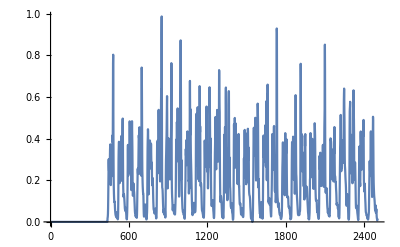

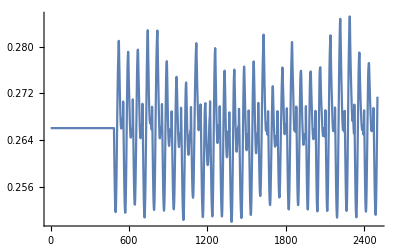

Sub03_(7)run2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382282.0.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382283.0.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382284.0.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382285.0.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382286.0.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382287.0.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382288.0.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.249382289.0.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822810.0.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822811.0.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822812.0.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822813.0.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822814.0.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822815.0.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822816.0.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822817.0.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822818.0.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822819.0.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822820.0.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822821.0.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822822.0.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822823.0.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822824.0.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822825.0.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822826.0.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822827.0.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822828.0.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822829.0.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822830.0.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822831.0.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822832.0.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822833.0.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822834.0.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822835.0.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822836.0.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822837.0.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822838.0.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822839.0.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822840.0.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822841.0.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822842.0.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822843.0.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822844.0.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822845.0.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822846.0.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822847.0.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822848.0.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822849.0.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822850.0.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822851.0.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822852.0.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822853.0.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822854.0.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822855.0.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822856.0.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822857.0.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822858.0.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822859.0.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822860.0.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822861.0.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822862.0.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822863.0.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822864.0.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822865.0.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822866.0.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822867.0.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822868.0.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822869.0.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822870.0.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822871.0.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822872.0.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822873.0.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822874.0.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822875.0.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822876.0.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822877.0.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822878.0.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822879.0.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822880.0.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822881.0.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822882.0.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822883.0.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822884.0.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822885.0.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822886.0.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822887.0.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822888.0.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822889.0.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822890.0.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822891.0.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822892.0.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822893.0.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822894.0.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822895.0.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822896.0.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822897.0.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822898.0.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.2493822899.0.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228100.0.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228101.1.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228102.1.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228103.1.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228104.1.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228105.1.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228106.1.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228107.1.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228108.1.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228109.1.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228110.1.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228111.1.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228112.1.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228113.1.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228114.1.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228115.1.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228116.1.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228117.1.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228118.1.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228119.1.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228120.1.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228121.1.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228122.1.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228123.1.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228124.1.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228125.1.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228126.1.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228127.1.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228128.1.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228129.1.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228130.1.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228131.1.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228132.1.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228133.1.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228134.1.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228135.1.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228136.1.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228137.1.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228138.1.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228139.1.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228140.1.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228141.1.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228142.1.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228143.1.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228144.1.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228145.1.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228146.1.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228147.1.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228148.1.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228149.1.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228150.1.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228151.1.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228152.1.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228153.1.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228154.1.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228155.1.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228156.1.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228157.1.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228158.1.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228159.1.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228160.1.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228161.1.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228162.1.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228163.1.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228164.1.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228165.1.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228166.1.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228167.1.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228168.1.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228169.1.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228170.1.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228171.1.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228172.1.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228173.1.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228174.1.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228175.1.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228176.1.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228177.1.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228178.1.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228179.1.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228180.1.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228181.1.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228182.1.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228183.1.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228184.1.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228185.1.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228186.1.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228187.1.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228188.1.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228189.1.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228190.1.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228191.1.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228192.1.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228193.1.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228194.1.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228195.1.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228196.1.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228197.1.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228198.1.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228199.1.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228200.1.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228201.2.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228202.2.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228203.2.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228204.2.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228205.2.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228206.2.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228207.2.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228208.2.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228209.2.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228210.2.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228211.2.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228212.2.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228213.2.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228214.2.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228215.2.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228216.2.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228217.2.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228218.2.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228219.2.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228220.2.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228221.2.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228222.2.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228223.2.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228224.2.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228225.2.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228226.2.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228227.2.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228228.2.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228229.2.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228230.2.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228231.2.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228232.2.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228233.2.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228234.2.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228235.2.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228236.2.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228237.2.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228238.2.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228239.2.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228240.2.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228241.2.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228242.2.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228243.2.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228244.2.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228245.2.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228246.2.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228247.2.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228248.2.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228249.2.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228250.2.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228251.2.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228252.2.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228253.2.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228254.2.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228255.2.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228256.2.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228257.2.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228258.2.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228259.2.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228260.2.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228261.2.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228262.2.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228263.2.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228264.2.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228265.2.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228266.2.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228267.2.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228268.2.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228269.2.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228270.2.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228271.2.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228272.2.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228273.2.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228274.2.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228275.2.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228276.2.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228277.2.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228278.2.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228279.2.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228280.2.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228281.2.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228282.2.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228283.2.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228284.2.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228285.2.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228286.2.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228287.2.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228288.2.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228289.2.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228290.2.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228291.2.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228292.2.9100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228293.2.9200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228294.2.9300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228295.2.9400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228296.2.9500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228297.2.9600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228298.2.9700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228299.2.9800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228300.2.9900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228301.3.00.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228302.3.0100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228303.3.0200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228304.3.0300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228305.3.0400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228306.3.0500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228307.3.0600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228308.3.0700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228309.3.0800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228310.3.0900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228311.3.100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228312.3.1100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228313.3.1200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228314.3.1300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228315.3.1400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228316.3.1500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228317.3.1600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228318.3.1700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228319.3.1800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228320.3.1900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228321.3.200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228322.3.2100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228323.3.2200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228324.3.2300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228325.3.2400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228326.3.2500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228327.3.2600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228328.3.2700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228329.3.2800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228330.3.2900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228331.3.300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228332.3.3100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228333.3.3200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228334.3.3300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228335.3.3400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228336.3.3500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228337.3.3600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228338.3.3700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228339.3.3800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228340.3.3900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228341.3.400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228342.3.4100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228343.3.4200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228344.3.4300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228345.3.4400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228346.3.4500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228347.3.4600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228348.3.4700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228349.3.4800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228350.3.4900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228351.3.500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228352.3.5100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228353.3.5200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228354.3.5300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228355.3.5400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228356.3.5500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228357.3.5600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228358.3.5700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228359.3.5800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228360.3.5900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228361.3.600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228362.3.6100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228363.3.6200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228364.3.6300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228365.3.6400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228366.3.6500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228367.3.6600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228368.3.6700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228369.3.6800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228370.3.6900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228371.3.700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228372.3.7100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228373.3.7200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228374.3.7300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228375.3.7400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228376.3.7500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228377.3.7600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228378.3.7700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228379.3.7800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228380.3.7900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228381.3.800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228382.3.8100.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228383.3.8200.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228384.3.8300.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228385.3.8400.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228386.3.8500.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228387.3.8600.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228388.3.8700.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228389.3.8800.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228390.3.8900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228391.3.900.2660504600.3766934800.3905801600.2788743100.317532100.5223758700.2913915200.3937018100.4133442200.24938228392.3.9100.2660504600.3766934800.3905801600.2788743100.31753210.00179408010819122550.5223758700.2913915200.3937018100.4133442200.24938228393.3.9200.2660504600.3766934800.3905801600.2788743100.31753210.0026972577118431910.5223758700.2913915200.3937018100.4133442200.24938228394.3.9300.2660504600.3766934800.3905801600.2788743100.31753210.00364445040809700630.5223758700.2913915200.3937018100.4133442200.24938228395.3.9400.2660504600.3766934800.3905801600.2788743100.31753210.00386381093169339660.5223758700.2913915200.3937018100.4133442200.24938228396.3.9500.2660504600.3766934800.3905801600.2788743100.31753210.0037408432604155910.5223758700.2913915200.3937018100.4133442200.24938228397.3.9600.2660504600.3766934800.3905801600.2788743100.31753210.0049299440464195130.5223758700.2913915200.3937018100.4133442200.24938228398.3.9700.2660504600.3766934800.3905801600.2788743100.31753210.0068367023456634040.5223758700.2913915200.3937018100.4133442200.24938228399.3.9800.2660504600.3766934800.3905801600.2788743100.31753210.009225586529660130.5223758700.2913915200.3937018100.4133442200.24938228400.3.9900.2660504600.3766934800.3905801600.2788743100.31753210.0125352721673928760.5223758700.2913915200.3937018100.4133442200.24938228401.4.00.2660504600.3766934800.3905801600.2788743100.31753210.0156100955491082580.5223758700.2913915200.3937018100.4133442200.24938228402.4.0100.2660504600.3766934800.3905801600.2788743100.31753210.0175383745336870870.5223758700.2913915200.3937018100.4133442200.24938228403.4.0200.2660504600.3766934800.3905801600.2788743100.31753210.01859019355665110.5223758700.2913915200.3937018100.4133442200.24938228404.4.0300.2660504600.3766934800.3905801600.2788743100.31753210.0210937008797129270.5223758700.2913915200.3937018100.4133442200.24938228405.4.0400.2660504600.3766934800.3905801600.2788743100.31753210.0263685451631124960.5223758700.2913915200.3937018100.4133442200.24938228406.4.0500.2660504600.3766934800.3905801600.2788743100.31753210.0348510872111427450.5223758700.2913915200.3937018100.4133442200.24938228407.4.0600.2660504600.3766934800.3905801600.2788743100.31753210.044440337018409990.5223758700.2913915200.3937018100.4133442200.24938228408.4.0700.2660504600.3766934800.3905801600.2788743100.31753210.051477721377686160.5223758700.2913915200.3937018100.4133442200.24938228409.4.0800.2660504600.3766934800.3905801600.2788743100.31753210.06011971132904860.5223758700.2913915200.3937018100.4133442200.24938228410.4.0900.2660504600.3766934800.3905801600.2788743100.31753210.075563709374680960.5223758700.2913915200.3937018100.4133442200.24938228411.4.100.2660504600.3766934800.3905801600.2788743100.31753210.090637569259780820.5223758700.2913915200.3937018100.4133442200.24938228412.4.1100.2660504600.3766934800.3905801600.2788743100.31753210.095767263823256430.5223758700.2913915200.3937018100.4133442200.24938228413.4.1200.2660504600.3766934800.3905801600.2788743100.31753210.093046247211122850.5223758700.2913915200.3937018100.4133442200.24938228414.4.1300.2660504600.3766934800.3905801600.2788743100.31753210.093158988088281050.5223758700.2913915200.3937018100.4133442200.24938228415.4.1400.2660504600.3766934800.3905801600.2788743100.31753210.09885177124634480.5223758700.2913915200.3937018100.4133442200.24938228416.4.1500.2660504600.3766934800.3905801600.2788743100.31753210.097478404778625930.5223758700.2913915200.3937018100.4133442200.24938228417.4.1600.2660504600.3766934800.3905801600.2788743100.31753210.081571914429704430.5223758700.2913915200.3937018100.4133442200.24938228418.4.1700.2660504600.3766934800.3905801600.2788743100.31753210.0595335246069095760.5223758700.2913915200.3937018100.4133442200.24938228419.4.1800.2660504600.3766934800.3905801600.2788743100.31753210.039276035226306410.5223758700.2913915200.3937018100.4133442200.24938228420.4.1900.2660504600.3766934800.3905801600.2788743100.31753210.0249824115937216030.5223758700.2913915200.3937018100.4133442200.24938228421.4.200.2660504600.3766934800.3905801600.2788743100.31753210.0169009158364230760.5223758700.2913915200.3937018100.4133442200.24938228422.4.2100.2660504600.3766934800.3905801600.2788743100.31753210.012514656533047210.5223758700.2913915200.3937018100.4133442200.24938228423.4.2200.2660504600.3766934800.3905801600.2788743100.31753210.0096185897380027220.5223758700.2913915200.3937018100.4133442200.24938228424.4.2300.2660504600.3766934800.3905801600.2788743100.31753210.0071174084516092370.5223758700.2913915200.3937018100.4133442200.24938228425.4.2400.2660504600.3766934800.3905801600.2788743100.31753210.0057424752566069190.5223758700.2913915200.3937018100.4133442200.24938228426.4.2500.2660504600.3766934800.3905801600.2788743100.31753210.0057474972739166990.5223758700.2913915200.3937018100.4133442200.24938228427.4.2600.2660504600.3766934800.3905801600.2788743100.31753210.0061085005198548430.5223758700.2913915200.3937018100.4133442200.24938228428.4.2700.2660504600.3766934800.3905801600.2788743100.31753210.00586236103167616250.5223758700.2913915200.3937018100.4133442200.24938228429.4.2800.2660504600.3766934800.3905801600.2788743100.31753210.00530433130559393450.5223758700.2913915200.3937018100.4133442200.24938228430.4.2900.2660504600.3766934800.3905801600.2788743100.31753210.005742674277447910.5223758700.2913915200.3937018100.4133442200.24938228431.4.300.2660504600.3766934800.3905801600.2788743100.31753210.0067861641261125730.5223758700.2913915200.3937018100.4133442200.24938228432.4.3100.2660504600.3766934800.3905801600.2788743100.31753210.0075524608731533170.5223758700.2913915200.3937018100.4133442200.24938228433.4.3200.2660504600.3766934800.3905801600.2788743100.31753210.0068698537249188080.5223758700.2913915200.3937018100.4133442200.24938228434.4.3300.2660504600.3766934800.3905801600.2788743100.31753210.00502697861512049150.5223758700.2913915200.3937018100.4133442200.24938228435.4.3400.2660504600.3766934800.3905801600.2788743100.31753210.0037806417032578750.5223758700.2913915200.3937018100.4133442200.24938228436.4.350.01768723475056280.2660504600.3766934800.3905801600.2788743100.31753210.0028892829459717340.5223758700.2913915200.3937018100.4133442200.24938228437.4.360.0210932774022643860.2660504600.3766934800.3905801600.2788743100.31753210.0021541788651216010.5223758700.2913915200.3937018100.4133442200.24938228438.4.370.0274918203553136050.2660504600.3766934800.3905801600.2788743100.31753210.0022026514371980780.5223758700.2913915200.3937018100.4133442200.24938228439.4.380.039178895991401610.2660504600.3766934800.3905801600.2788743100.31753210.00292624960730913840.5223758700.2913915200.3937018100.4133442200.24938228440.4.390.063922231678378490.2660504600.3766934800.3905801600.2788743100.31753210.0034664852088945070.5223758700.2913915200.3937018100.4133442200.24938228441.4.40.108173573999435890.2660504600.3766934800.3905801600.2788743100.31753210.003673337307752540.5223758700.2913915200.3937018100.413344220.01960986040865690.24938228442.4.410.160903670562545180.2660504600.3766934800.3905801600.2788743100.31753210.0046458619745209570.5223758700.2913915200.3937018100.413344220.02154272974124270.24938228443.4.420.218056275513797330.2660504600.3766934800.3905801600.2788743100.31753210.00587278166554020850.5223758700.2913915200.3937018100.413344220.0237694820693094560.24938228444.4.430.283692883199893050.2660504600.3766934800.3905801600.2788743100.31753210.0063600948772855050.5223758700.2913915200.3937018100.413344220.0247080822301384530.24938228445.4.440.301022535321132770.2660504600.376693480.00267795348312701650.3905801600.2788743100.31753210.0070257061684836850.5223758700.2913915200.3937018100.413344220.024868990842218930.24938228446.4.450.269197510423166360.2660504600.376693480.0056322341423371580.3905801600.2788743100.31753210.0074223716777205150.5223758700.2913915200.3937018100.413344220.0258972216433677670.24938228447.4.460.24598477397446820.2660504600.376693480.007928785465835570.3905801600.2788743100.31753210.00732525637364966550.5223758700.2913915200.3937018100.413344220.0273194037908332240.24938228448.4.470.24606126691559880.2660504600.376693480.0093212723847890150.390580160.0101764607254220050.2788743100.31753210.0071962415303000830.5223758700.2913915200.3937018100.413344220.0282208415927572530.24938228449.4.480.266819119214661060.2660504600.376693480.0086860336767146840.390580160.011821267513045620.2788743100.31753210.00766345478459426550.5223758700.2913915200.3937018100.413344220.0290557072510015460.24938228450.4.490.28044069918121730.2660504600.376693480.0075364337142983020.390580160.0134660577338487420.2788743100.31753210.0080543197505988150.5223758700.2913915200.3937018100.413344220.030364061447323060.24938228451.4.50.251448079475185940.2660504600.376693480.0084495581498286520.390580160.0143326545507944420.2788743100.31753210.0085749086191084880.5223758700.2913915200.3937018100.413344220.032280472500348620.24938228452.4.510.213562101277668420.2660504600.376693480.0088228631540318920.390580160.0138106352852736330.2788743100.31753210.0096999553564440630.5223758700.2913915200.3937018100.413344220.0346548085025772250.24938228453.4.520.247100692346433730.2660504600.376693480.0072450373235438720.390580160.012669711102354920.2788743100.31753210.0107433709446722140.522375870.0038108962754121720.2913915200.3937018100.413344220.0368893257338262160.24938228454.4.530.31116139998505590.2660504600.376693480.0055950622753937360.390580160.011499588890405840.2788743100.31753210.0106504708089907720.522375870.0067700189955376070.291391520.0071125291652416350.3937018100.413344220.0389263011987151660.24938228455.4.540.346554607760431570.2660504600.376693480.0059776436552023970.390580160.0111264462224009570.2788743100.31753210.0094374296376755260.522375870.0081371551091023940.291391520.009551697606518030.3937018100.413344220.040796598740451290.24938228456.4.550.36692403071148990.2660504600.376693480.0088812491525915760.390580160.011903406341286590.2788743100.31753210.007789809189852790.522375870.0074641352847712160.291391520.0098105713912576450.3937018100.413344220.040833903731374940.24938228457.4.560.372120392766137560.2660504600.376693480.0143286144762876640.390580160.012916138462927360.2788743100.31753210.0066191877365476530.522375870.0055193809054850370.291391520.0100289991951722670.3937018100.413344220.0374618464967633940.24938228458.4.570.321098531898602050.2660504600.376693480.018537704487073250.390580160.0132483587609717750.2788743100.31753210.0062782049569362450.522375870.0045027515894451670.291391520.0104891852506845750.3937018100.413344220.0306981831251982650.24938228459.4.580.240527781187400370.2660504600.376693480.0181383225701004440.390580160.0126187353623998490.2788743100.31753210.0058053950203527070.522375870.00582045768393277350.291391520.013634847953298430.3937018100.413344220.0243960684386458040.24938228460.4.590.178828429338403460.2660504600.376693480.0143219963119881020.390580160.0111864089954861240.2788743100.31753210.00456954161979566950.522375870.0066003510747867820.291391520.018467721143936180.3937018100.413344220.022297934228419840.24938228461.4.60.176679497278324940.2660504600.376693480.0146108260580581350.390580160.0100308450158216620.278874310.00161295649205937240.31753210.00295531404004086960.522375870.0045230327010974630.291391520.023309126405423010.3937018100.413344220.023684376509602530.24938228462.4.610.212914573594070620.2660504600.376693480.0226463157354881670.390580160.011569470797252950.278874310.0040837151322427460.31753210.00212268811024442530.522375870.0044131923770464520.291391520.031548913358902810.3937018100.413344220.03090557507341160.24938228463.4.620.248989838418701230.2660504600.376693480.0317046423170833650.390580160.0139623415676486620.278874310.0069161614744133220.31753210.00259401957862854260.522375870.0073284340560970280.291391520.044278664718683990.3937018100.413344220.044670931248132070.24938228464.4.630.27137620964252020.2660504600.376693480.0319435166177596540.390580160.0159850935299236180.278874310.0087028654360285250.31753210.0031184923065473670.522375870.0090362150134574630.291391520.064592357548749940.3937018100.413344220.064666366011648880.24938228465.4.640.31234952737361640.2660504600.376693480.0276248416834085530.390580160.019508259488281620.278874310.0102705768181285750.31753210.00346953501339155670.522375870.0089736403138299170.291391520.09510703341055510.3937018100.413344220.087686147169801260.24938228466.4.650.328908633263858050.2660504600.376693480.0222886279239494330.390580160.0223683399275141780.278874310.0121749648620447570.31753210.00364958634109582850.522375870.008395769621885180.291391520.137566599684976780.393701810.0371663483715183460.417277930.109540028906135410.24938228467.4.660.27678284905120170.2660504600.376693480.030404918237758580.390580160.023609598970583650.278874310.0151621367875194590.31753210.0043913633749653980.519324260.0101495747522803140.291391520.203876774542083940.393701810.0466712040041464760.421286250.131353264337491280.24938228468.4.670.2607654866372790.2660504600.376693480.049490211098547820.390580160.0256145352080385660.278874310.018452887619017450.31753210.00536069135405689650.516071230.0128488179651455770.291391520.29817460428266510.393701810.061424771791519240.425422220.152370993294620750.24938228469.4.680.317434225219102640.266050460.00384702431130363140.376693480.0559460784373395640.390580160.0285744924624729970.278874310.02169658841662210.31753210.0057543988117147980.51278170.0149816129295201940.291391520.39265333248963740.393701810.079676028200196510.429455230.170159488705977440.24938228470.4.690.304745071327782170.266050460.0081365413541290840.376693480.0533502508838315240.390580160.0293252090116565630.278874310.0256336839228567540.31753210.0063789155998143920.50933230.018540741866236640.291391520.43723888074434460.393701810.092711071047259520.433562550.18180745350008680.24938228471.4.70.220121830070383270.266050460.00873271985034470.376693480.0423864609417302640.390580160.0247463942923822240.278874310.0305343048262259640.31753210.008804924412181820.505874150.0228763494992799440.291391520.41735511582004680.393701810.094254950038478170.437625440.184367830007741460.24938228472.4.710.227576442741665050.266050460.0078697790120948010.376693480.0274209333086323470.390580160.020258336928994110.278874310.036172427668826840.31753210.01254465887567370.502519820.0291758356684886750.291391520.37414018526193020.393701810.095264883958217570.441471630.178925509592582050.24938228473.4.720.34981246113987020.266050460.0072655763102036320.376693480.0188472502485951820.390580160.01919079818041240.278874310.039954574850690780.31753210.0171423205238186650.499282440.0345197964944660850.291391520.346379361084865170.393701810.099454360803903310.44500550.169757826133508760.24938228474.4.730.415535441164770040.266050460.0073032205059094190.37844020.0161696577605460.392281540.0187656461399526640.278874310.0395384121303133040.31753210.0215677366801457870.496274040.0351083452109042240.291391520.316907389730185950.393701810.099023210116051720.448125390.157258409595338020.24938228475.4.740.38410443305421550.266050460.0112602300454999840.380118690.0167981084054207030.393878130.018578550923714230.278874310.03587056208599720.31753210.025087585011199790.493680770.034197074871174350.291391520.284174252134663130.393701810.094859455361096260.450687330.13944032593661090.24938228476.4.750.39593343152903260.266050460.0159073652183508720.381540020.0185275966959280380.395115110.019072355055974160.278874310.0330649237138072250.31753210.027201214273091260.49160690.038346880295824390.291391520.268700772165353930.393701810.090941481211871250.452643640.118553882978800720.24938228477.4.760.55711989997471380.266050460.017701477150203650.38262550.0198398804625285930.395696310.0185571752380061130.278874310.039610191948045340.31753210.0277738568090950750.490091310.054824540307031390.291391520.25859947036053330.393701810.079941723962463310.454028010.10540116217378090.24938228478.4.770.7615707992104510.266050460.0179986602678366140.383359510.0209489036395784050.396091050.0169880207485155750.278874310.0610882445109252950.31753210.027823530671933020.489200990.082427866307919370.291391520.221379386090482380.393701810.0624033166906920250.454805450.10832241143577690.24938228479.4.780.80284539995074130.266050460.0252091842084194340.38379860.022187366795764280.396368720.017056311273987960.278874310.092629804666208710.31753210.0285642489255090030.488960190.101216755524642030.291391520.167865808577906840.393701810.046591096015796070.454967540.126199854433625470.24938228480.4.790.63093842391265580.266050460.0469408439876830150.384004360.024387461607775810.396565090.023737373994720890.278874310.12867751571083920.31753210.031466053587707080.489332680.098605155547461580.291391520.123762561741247360.393701810.03651368044834060.454513360.164662621092079580.24938228481.4.80.41976044533493960.266050460.09016089761426860.383972990.0273891228927129920.396615840.0397523006183802960.278874310.165137318629540150.31753210.037782692058610220.490144190.100390502082150920.291391520.10622062548339140.393701810.0329404303132186660.453574070.230208991144385640.24938228482.4.810.279044705906580870.266050460.152566466378850630.382846950.0301422042520362140.395682430.063227532223450620.278874310.201222636734731060.31753210.04891521518911020.491287820.139577823350608230.291391520.116538580027417830.393701810.0355587466342502660.452293950.31983097153029010.24938228483.4.820.198356096046466230.266050460.223092973193212360.379376620.0332847178460345740.392667860.097452557906671830.278874310.23457577385404380.31753210.064831571871218560.49309840.194870412655979960.291391520.13934728543937760.393701810.0416216198012763840.450369560.420061769974480360.24938228484.4.830.159154049443693550.266050460.285152748193082560.377882810.047032141119033980.391680090.15413388950137320.278874310.26029001039170820.31753210.081282581388602420.496356880.225363668529742270.291391520.158667198927338380.393701810.048418498227472840.447155760.50878478563233190.24938228485.4.840.133333229194663030.266050460.288070234006957360.378158110.070240404495696180.392015230.200666910860041820.278874310.272019587284285050.31753210.094498364899283450.500064970.238107107321890860.291391520.164820103439841460.393701810.0553275617653394840.443327260.56041890034628320.24938228486.4.850.115418319199808870.264364470.245483795397461760.378255380.098934743201911910.392113470.228166532298965520.280541390.276865722656995330.31753210.10281586035377060.503300910.234388833386030.291391520.15633517776164760.393701810.063387400980832190.439655270.55675156630064090.24938228487.4.860.102463601594696210.262572310.27205646391991870.378766830.1311022636211850.392594160.25096143292529150.282266220.27923481807154590.31753210.104329106512779190.506133680.215888319905937760.291391520.139966153927396060.393701810.073438667910715450.436246320.49775463455216630.24938228488.4.870.095610957954286870.260778490.347344774439066030.37949810.171401448745945960.393283460.265119756194406640.283944440.27113752557004210.31753210.102721665228909950.508582010.196147588263358650.291391520.129695116440627370.393701810.08509848950928760.433224310.40369081226974990.24938228489.4.880.095997234080348770.259115010.36194972746634790.380293460.250733577552411270.39403690.32856204981288580.285458120.25384492811294060.31753210.098323087817907550.510618150.16517673049317440.291391520.140969046214571850.393701810.096297281098481740.430653990.309311657643102530.24938228490.4.890.097478495686039320.257595920.289574388818664540.381146950.357777497011469550.394854650.39991844152369180.286805020.2278276846429920.31753210.08434062151848120.512325550.125459483368634830.291391520.182732548902463240.393701810.104218976545966370.428420230.254313370736184930.24938228491.4.90.092445280565871260.25617720.198574379688241540.382082050.44525820387562230.395762690.41099308069547020.288032780.190105052713052780.31753210.062084011805847940.513799280.086198848024766810.291391520.250724577568772760.393701810.107764437620473230.426428420.263583510246381440.24938228492.4.910.079358439274535220.254904960.125219707525525720.383055840.462610773252817850.396720130.35434493762359590.289109320.146305842943723870.31753210.039712034767840610.515079690.055747654168425460.291391520.337139777511575260.393701810.10854902805322490.424642760.3186861572221260.24938228493.4.920.063933101187882540.253831170.076954858149910490.384004070.418801211551377730.397662470.26293357643925170.290000130.106496985694988280.31753210.0242688773496713660.51615840.03552424564990240.291391520.454531192719151660.393701810.110336835965017460.423090460.383101255464712350.24938228494.4.930.0533780329747136560.252994790.046858045882181820.384894060.344057066750495970.398556430.190839289667519170.290682810.074248977658221750.31753210.0166161897110243570.517009480.022169047018192140.291391520.57409723348127820.393701810.114946225440940130.421809320.42903220836477190.24938228495.4.940.046624316745310810.252377360.0328166090033243860.385746170.28801947445234540.399420920.159209629762388060.291180560.0495384920768012560.31753210.0127174226573624660.517686050.0145827017313932530.291391520.65402091165226620.393701810.124347752356661790.42072470.440921583838221050.24938228496.4.950.040172731274522670.251951860.028539460552410030.386572690.283441485384315240.400265690.15512199304571720.291520530.032458097217023560.31753210.009697891101790290.518237250.0118716849403704020.291391520.68648381515874570.393701810.14189490749992540.419773160.418379059077294340.24938228497.4.960.034319431686143760.251720230.03267330624677380.387370030.326403325720696360.401084590.17247467527169730.291704560.0216116622671041550.31753210.00751078946605012850.518680030.0120191887713041980.291391520.64713332514535860.393701810.170802971195966240.418929050.36944497136271550.24938228498.4.970.0316741980556080740.251671680.050972621148307880.388127850.350496766236653930.401863690.18842120131044920.291743030.0146241265672787370.316475420.0062214286574723270.518992380.0107128845389710320.290389840.54261550510399540.393701810.215630833023375880.418221760.30577631214642720.24756703499.4.980.0305371051660030670.251914130.080078665005973080.388688990.375354324045287570.402441530.192980885011825340.291550560.0106254980655163930.315300860.0062928176993651640.519163030.008294628079615420.289279540.44149606252083460.393701810.273165383708974750.417673460.240287534127215620.24568967500.4.990.0274737663805329350.252445820.115952475049583230.389014520.407644982903186960.402776930.197436303566919940.291125630.0095535106863718740.314056390.0074003267610901950.519204380.0078481979918092640.288106180.41636655686709980.393701810.3306759629308920.417267450.180945834292919850.24380003501.5.0.0252863973548616040.253252610.148637634979946140.389088830.44189582764279370.402853480.197390861144069290.290473410.0097765982916828260.312771520.0085976634274734130.519126480.0097133279833678640.28689740.45210997053032780.392865270.375159532854403840.416978530.130141940489349070.24187731502.5.010.022670403367888810.254326160.16816548519015030.388891410.404330279218313440.402650940.177520517262455130.28959150.0107253974030095230.311479290.0090481696169402920.518956050.0119432179949698990.285684210.448063225819103740.392097850.40068536949048920.416768580.088728625425508130.23993115503.5.020.0224839924328485360.255629350.16486018207950020.388423480.285976049477362770.402171880.16296306365582510.288499180.0111563732722275170.310225390.0077995859228135910.518730680.0110104084690993230.284509480.358230062487789160.39138930.41022492990396590.416606460.057629781304290060.23798241504.5.030.029192288009100650.257085040.15034151319448630.387733440.205014433012879140.401466760.174443907773490060.287250470.0114395674881684790.30904220.0057180680221440510.518456020.0071352740816177440.283403280.23607946028523020.390782980.40710971939469220.416513440.0367328765309287150.23613775505.5.040.0395902210028582850.258723840.127805815683273540.386787230.191340561292963650.400503750.188744163902781370.285808160.0117230261424271280.307931340.0038955064886279120.518183630.00359133579410151130.282366740.12850646296092330.390216060.38846264449844520.416421170.023877378541803380.23437668506.5.050.0458083830788724650.260442380.117132418935164110.385654290.19925821733912350.39935520.19248979342146990.284253570.0111187389946605740.306938840.00304166106162994870.517940110.00352510627792482130.281442320.068146076121328250.389713770.35025202672588960.416332790.0154554003040876190.23278582507.5.060.044833702197125880.262233350.11927550128094240.384312770.176286256128454250.398003610.17830959577132360.282587010.009888641617479620.306116540.00277592743688216030.51782230.0068063467012327760.280677620.0451740439457162940.389191490.29846104024097970.416145660.01217701643489720.23133549508.5.070.037280568102108090.264058820.115713070413249090.382813050.133794693710484660.39650080.15865185578899920.280838990.0078832651096846660.305441380.00281104637474155660.517844820.0090443755258345860.280050440.0439377224135582140.388599010.245246661125767820.415824290.0139119688704331150.22995535509.5.080.02865203702781740.265911010.109156477396034580.381151460.124263369466781670.394846050.139477450207500880.279013840.0064423446264392950.304936080.00272038161863249550.518031150.0102648968185655480.279581360.0534111035685900860.387922470.198578374563131680.415350330.0158474839701134750.2286521510.5.090.022013435014818330.267750430.09735122857842960.379374630.11762001233424530.393086810.110366332636956550.277149370.0064263369053447410.304593220.0028143889037468460.518386850.0125081387757611360.279263160.062829470404553070.387139780.16152846623122630.414711720.0145930242724947230.22737753511.5.10.019010877696125070.269528490.09506445082683370.377520260.122857412036526950.39123560.07529376113861380.275297440.00589002801417544150.304446940.00321158916810961470.518949740.0151828000211694620.279127430.065724593277136450.386219360.134464266806616740.41387750.0104269028992816110.22606468512.5.110.016385889310339360.271252040.084161924103864280.375543910.120453529076256230.389332720.047465308726418230.273455310.0048904143092590280.304576610.00421720114087373050.519809760.0152995355534228280.279247750.0618541205826910.385106260.117832359373514230.412764620.0050827455377906150.22473987513.5.120.0139642681943106930.27279220.084881076889952060.373604820.080612338322970630.387451670.0344536602987427640.271769760.0035976499816980080.304963760.0054724076352752020.520892880.0126448574024040530.279607050.05664947166909240.38391610.111437510837883740.41148110.0012341946053917740.22359187514.5.130.0123487532615534720.274179250.093986688206599580.371671480.0450068820422250960.385586090.033064106014270850.270219780.0032786233095397660.305617460.0078917691755631020.522167140.0092548218780160710.280213960.0542315810810622340.382694260.111788675204650160.410063440.000460287909548792870.22272024515.5.140.0128466068497200950.27546070.087508189778342360.369646650.0278884403635132130.383639430.0354651114113238850.268760740.0045314195898533350.306621670.0102595845029963460.523679860.00761839799429998850.281147240.052405826676585210.381415930.113643685883928730.408458690.00072205423780851880.22214434516.5.150.0203907423395759750.276566930.08792349713825390.367618550.019928632649998760.381690730.0323821861155906550.267480240.0063070785549072930.307957440.0119858251625939920.525419070.0087729583712744220.282391080.0463843488566872960.380063880.113750325376008710.406651490.00161071600539304420.22179633517.5.160.044058452025425930.277502910.086289759134561830.365611410.0165280817138588470.379755190.024480110443754580.266381620.0074267070631489070.309559590.013747015774136590.527254590.0111253378614126680.283886730.037642027204817150.378759610.111699445759239550.404788180.0052698255132444980.22162691518.5.170.099405677722501360.278350.051755772160731720.363562340.0149686531248223610.377765040.0180271617589662160.265375310.0071469661491628040.311350170.0148064366077640550.529092080.0122750381476858380.285563120.027960953321887610.377586690.108895097187558780.402971010.0083849376796391460.22163488519.5.180.198185176130150830.279160840.0253026248620503050.361394540.0147798423746068140.375640160.0148996189499837080.264401370.0064553843153822220.31332370.0149619030304297290.531043370.0122659244615661440.287416570.0193741448445525450.37636010.106630029806156920.401006650.0097653223100476260.22165444520.5.190.29660130685613570.279973510.0190207819847822250.359068810.0152002861033040360.373337470.0153533597572509810.263414750.0059387609996107330.315432350.0158150258782719070.533121240.0119637290599449960.289403690.0119553662032476850.375016710.104850474694725180.398827910.0102696047297944850.22169305521.5.20.3406811593435940.280675520.0174363653137251350.356721150.0155001751930180510.370983460.0178568715630744270.262554040.0053292811722539990.317662830.02087624730671790.53522350.0124043801290264470.291515660.0064429874529626840.373685510.102577726331856220.39657910.012236397164280810.22176881522.5.210.36253347388306930.280988220.016877830692998730.354704650.015325626187436860.36891480.0193015222914244030.262168130.0039599311641584150.320007960.0319974352261836250.537392950.0139169621307181770.293751530.0054384956005614110.372287920.099155043496817170.394171940.015448071739160990.22196519523.5.220.38473677655882980.280516360.0153286092120126570.353498670.0147267963975011420.367589070.017883808861044680.262749860.0018557515718885920.322483690.048975770458695080.53953860.0123435539504115620.296132550.0054417769423458550.371010270.095589851330131770.391790270.019662152965771330.22250099524.5.230.38434853347360910.279312610.0129655464387471750.353070720.0144432795776565230.366976230.015985439377602450.264217910.00214231460101599540.324986430.066325944053164830.541443240.0097834616567898220.298560840.0063882218502081370.370104060.095012501961173650.389713360.023820915202378550.22360977525.5.240.31581949879725380.277874740.011767097752019370.352890810.0128074385270284930.366573610.0152365128420974970.265941310.00388465505077864770.327344550.076497880438206160.542889230.0094760904154719190.300868260.0093109759645847830.369761140.100612307951525380.388191940.0249321090414912280.22537848526.5.250.25495140343959090.276783340.0110193215876163190.352379660.0089082425550389530.365835090.0141523326946152790.267227460.0044488581044389810.329416530.078909852297970180.543687030.0097558527373454110.302913660.0131997714004152730.370157650.112743632841922820.387481990.0231708154570399970.22777464527.5.260.220778949876595660.275842010.0112499087731765730.351861010.0053778025815305330.365089840.0132447270716574260.268321560.0041137562182209990.331150770.071395444745095740.54392770.0085267711435989440.304641740.0173271097970211850.371112750.128002972269707470.387458340.0218530424139392330.23047871528.5.270.188789038630786970.274714820.0129239393758363140.351756840.0024221750390940450.364759120.0125088047767371380.269613170.0034700582964102270.332567050.057004619570182140.543728080.0046580414508097690.30606630.0190434298917904930.372466120.140799658629932630.387967470.0195234171345748730.23334666529.5.280.186198694180540050.273469290.0160424412337897280.352017950.001991360909842220.364809280.0134148134118446830.271016950.004464383134621440.33367780.04404091950636230.543203770.0024878417777187320.307193210.0193263630368261980.374041710.147492937848514580.388852260.0175383967766245060.23616269530.5.290.217226481829230880.272280650.015288698559635920.352463230.00379703659100823340.365076250.015501848562921020.272333740.00654719953584811250.334501010.033726085845002750.542370890.0038884046716909520.308034540.020060784160807320.37582050.147462151775952870.39010020.0165180133951976850.23890622531.5.30.249503554473169160.271195010.0129840634022979330.353052130.006710301684823950.365529620.01669130897107560.2735170.0077003377342386770.335056910.0242536307656716420.541208270.006932352641285980.308605890.0214324959245691080.377841620.1406584740786710.391760130.0185507102570684930.24156325532.5.310.262742241473757350.270227980.0135814238539666480.353768390.0113471592086396670.366158620.0171742232601235880.274555420.0086242041581577260.335366440.0171283870682844530.539687170.0099687713840662380.308925210.024135194903386630.380162270.128662772870984380.393897050.02422157445193130.24412429533.5.320.26022634274468380.269348830.0129744516111783160.354646780.0200469433993670650.366999920.016847242876306120.275486790.0092279468790540940.335441980.0121197109826331960.537872040.0096388342365892420.309003270.0257740153701175380.382708230.113430008697349040.396432040.0279678593876652240.24652958534.5.330.233137209616965740.268522330.0101555861624445490.355726130.034486767440626420.368091820.0164923005041363760.276351420.0100206667903785640.33528770.0082484363355636510.535835420.0075969947783947790.30884390.027410534704859990.385393020.096282948761314340.399269260.0295938191567457350.24873834535.5.340.206881377153631560.267767940.0066193667221246640.356982460.055726106683283270.369408060.0166896153302052530.277131360.010831787374361190.334902730.0058013730811138990.533607020.0072868006970549850.308447150.0354186376619482140.388182280.078333844294492240.402364110.033144053751519960.25077836536.5.350.243680671327147460.267145060.0041129407649620770.358353870.068439474795247850.370883430.0167882913417847570.277768730.0109184037628898430.334275420.0049097257507149810.531202340.0073723254872617480.307803440.051244355058145970.391057270.061014689474163910.405692110.0378972448270932650.25265597537.5.360.31952639889275620.266693260.0045601882686461970.359794760.050170733189294850.372465620.0155686543509902750.278227290.0112237321216160370.333391640.00485566218108750450.528629050.00648477267025015550.306902010.06872088702570020.394000810.04678075890895470.409229630.041180404293351350.25437852538.5.370.348442660259774660.266392430.006184842271827920.361323020.030061235578855230.374163380.014013268435901870.278530880.0122152515536652750.332228210.0056321026992496690.525901990.0046555054896395190.305724270.07825824348468980.396977290.0386259078150499940.412936210.0405860943998738450.25593289539.5.380.31330864364033210.266156070.0082505418632104560.363019720.0270087355104224780.376046160.0157941162060327540.278768450.0135323743065759260.33075720.0069851552266661260.523026780.0049058745338443560.304248090.07924149829086460.399950790.038858658290853830.416776580.039133783979576140.25727426540.5.390.35286632496724720.26600890.0107374308640233160.364841310.041220452607112680.378060330.0230067253823464380.278915930.0151069856209066450.328946960.0084650522615474650.519999670.009183597108585830.302448430.092021346456987520.402894050.048891579350538940.42072110.0426479508397031650.25837281541.5.40.41227723735381740.265982120.0128574446046974540.366725050.0624238117198843150.380132230.031729832878917330.278942720.0157818171563712880.326776750.0088646253032118840.516800010.0131418377776388390.300310850.119438304851534250.405802030.064768117682739230.424759660.05678585043700270.25921801542.5.410.34913362217653570.266105090.0130847603925293450.36860740.06984774910251780.382188060.0358632793053180470.278819570.0155322316101392780.324232580.0083680011771398570.513437540.0135771461835303630.29782720.158654559348272270.408637140.075894848430125030.428843530.079245359127146630.25978847543.5.420.22706738241057220.266347880.0115348146388046250.370474020.062093481043527680.384201870.0338000898644316360.278575730.0154771824972412750.321362960.0078786983138633310.509874660.012870655325543560.295052040.204154332014015420.41149830.085686351654365360.433051860.101169421960686850.26019877544.5.430.197548738110585260.266752160.0089952066437809060.37221880.050703197860236570.386057330.0269424154875567460.278167690.0168780456623566430.318288970.0080891132777373330.506330360.0142943130204281080.29211090.241927718750106440.414220450.103826468476965760.437168620.118012209956850580.26040269545.5.440.26324721452778220.267186540.006645119901444550.373881620.0411333964819963340.387782070.0185129889669672750.277726470.0205274579058134060.315128190.0092768293336751030.502815690.018633780065759370.289116560.27861331344844610.416849910.126790985876535280.4411770.133091648682299970.26052488546.5.450.27461466280368240.267569380.0088724063894549970.375477260.0275793478930676550.38938540.0131704300932096890.27733520.0260188936748390780.311914850.0108498777550255690.499394320.0220927886243203720.286092840.300434926126995460.419281820.137555363235996850.444900460.14843155139905310.26059594547.5.460.232064679289431110.267662170.0140390680549777880.377186180.0164695990177008460.391045810.0139065669859811530.277240020.034145418941179950.308796310.0114054269587590630.496188630.0235079080429631130.283173670.252974840830664070.421449710.125036836887997050.448209350.163037936646140.26064193548.5.470.281383620621675160.267474860.016539973723882230.378921340.0132106046240138550.392689090.0169243675244283920.2774320.045923916607695710.306002920.0121212245574947170.493399720.0272909404780517330.280572030.183859074688273060.423268810.10833505519948810.450960710.173949431818454460.26069068549.5.480.388866603620102840.267201630.0156946664772026760.380443190.013794962636832210.393884430.020511459039394560.277711090.062252975513251670.303674760.016751543763128610.491161360.036138729155137840.278410920.141269127161938460.424678260.092278238600605290.453074020.178934792276108030.26073947550.5.490.45333537314233750.26698710.0174080547524663040.38158530.0153234482961023350.394492850.026184489025696860.277929410.083509298988826680.301896910.0235240469055002480.489562310.0542120442954091840.276760080.121358496086801530.42564090.071601565745574510.454505890.177406936826492360.26081163551.5.50.48440088809731350.266811470.026728766135354580.382376060.017736976241386360.39491620.0335906235061582960.278107610.107331665073458910.300699230.026932533684242640.488618410.082968669457629620.275645380.097584081333585230.426172630.0554810159206650460.455290390.173982762085673180.26091487552.5.510.49620881230196390.266622930.043170370539866360.382869820.0209205629711216870.395224780.042794199390402230.278298390.135112995247564340.300110860.0260804141408531340.488354840.109286065573980980.275096550.099866388984722390.426254170.059819197840068340.455429660.46508390064045110.26101499553.5.520.44439616875847770.266568840.0462406342241998840.382954370.0202388571698002320.395291390.043513468592202820.278353020.15991169470009980.300056240.03347859396864930.488703730.111177690492254770.275045550.10945324832952380.425902190.057436857776412250.454983730.45261671490996440.261051554.5.530.303580010867577970.267389190.0561001169132040940.381860550.020337968256085680.394348560.046054699639416570.277519640.183020022562222130.300496630.042052975821178090.489569430.108970054514098190.275456510.133973409496234960.425188070.054304835046567860.454036150.45223830401204640.26111063555.5.540.20162020015503440.270584910.090229021465911050.377780750.022768272402219120.390699990.0593502069276056750.274173850.206370689010020870.30168060.047099661683035750.49116050.131979763312253450.276558960.16302669834021150.423998020.055894631499885210.452408720.45790250219768320.26116743556.5.550.162413904962974250.270609370.111682878779945020.376079020.0271415299421953850.38986810.074395123629911170.274147620.240625876534189630.304919130.055361339697730590.494323090.188587943552429670.279565620.185654663744037880.422012310.061062313868268140.449380630.45995185102764450.2616785557.5.560.1376092852043570.268253420.114033358337952710.376490970.036492894994614620.390364840.092668550497286660.276630450.2862988070336320.308899230.07617694799354230.498119160.253126133975824230.283269760.19346719732126370.419608420.066586181805459170.445554140.449329986717298570.26252658558.5.570.122349415476035740.266412680.144846786580418750.376610490.0495284349461908160.39049830.11016339911956560.278510490.319894508237535350.312081340.097895357643966950.501595880.26845484174800950.286249110.18349785717110820.417075760.071505306225757610.441697880.42151991803681150.26313516559.5.580.119510552216704940.26463980.2380604116201430.377014390.074561255562039380.390875220.13919304925035610.28027210.31052328398515920.314428530.09746849130206390.5046840.226410277846605640.288456760.162750703765673380.414479850.076882450040340250.438007850.384214195195361760.26321583560.5.590.128283819000443580.262820980.346725344773091860.377724520.127503472345096460.391541490.228211642339091860.282029790.26254077881953040.3162020.081090857838917910.50736030.174744834245876250.29013110.146218964706762740.412054160.083566359725213520.434694890.35389081512182320.26296553561.5.60.13407833556730480.261026510.41248933709742150.378565360.219923499428500950.392333580.39128664086157070.283715250.228329411972936740.317626190.073664096420981350.509703250.149349909421811420.291480870.153531265729007130.409817580.0878500898729830.431741580.341048171775892640.26242991562.5.610.12890912836011270.259391790.427063073465701050.37939550.35783388116339390.393117760.54229838789662510.285209080.230136892506128650.31875260.078971174488628930.511652060.153405582675910620.292552420.200745138276450520.407862540.084461830095462960.42924040.339315624058779630.26171982563.5.620.121850771406285960.257843240.39121268685120050.380306370.4708576313742540.393989350.59500123132988410.286588020.231924968467352280.319585270.086674467787690240.513279450.167820450976509630.293347160.287533178457005930.406111660.077960840407642550.427105760.33662815663193120.26082149564.5.630.112845654239163120.256395660.2865519253610860.381278340.478809737592889530.394931460.56352932184543070.287845610.209544747602960880.320150740.086840372890898350.514637270.165190612730354240.293888260.38850867688205920.40453970.074469063292032680.425288310.335764527206769640.25979003565.5.640.10236283535883570.255125430.177121323783830750.382239460.43800267122050980.395873880.46264007924336170.28892440.164215319534600360.320463780.07449379298615420.515815670.140115073316023380.29418830.46807754753543830.403045520.075362954263532050.423666970.34560357153828810.25860467566.5.650.09214442885616360.25408070.111657950275811520.383125570.37087827464713960.396751530.322698729786447370.289794560.113166992992464720.320566830.057016201054159210.516854590.10733642512278060.294287140.51601907257225140.40161470.081393070957727120.422202450.357200633441433930.25730316567.5.660.080752938500840550.253266870.082028933590260210.383939570.311965470540466750.397566940.237341280111147750.290461790.077529244622818670.320461320.043909624187161480.517771230.077273101329682330.294185940.5544526366382350.40023710.093532538562083170.420869680.35549147304698870.25593981568.5.670.067653838307740970.252639830.079790564113712480.384723730.276832622575699460.39836120.23701284321891490.290969610.057812588113855570.320151670.034216605116068170.518560070.051614839727390540.293889160.5836610096066180.398930440.109940749318672430.41968040.34242139951229290.25454546569.5.680.060676515749705920.252140330.108172913543401030.385525950.29363593900236370.399180390.32008658024066090.291370250.043323241254799530.319648240.0248745738824542730.519267110.033307575961452630.293407370.56355562428150170.397634290.125290356450013050.418576540.32372950289777740.25303347570.5.690.0589216139371101160.251772010.150039800524634360.386336770.33966802978864410.400013080.40819506733504920.291663480.0308412318230547320.318959660.016977510177807450.519901930.0222024123453173420.292749830.48120587655619630.396329170.134487686689215460.41754540.294015563905547340.25134837571.5.70.0567501797055903550.251560350.163406360552658560.387111760.33019810256029970.400811930.38627655081961350.291831150.0213698281651449330.318114030.0111023658354440780.520400990.0161049636715442230.291944470.393564546112850130.395106090.135445347167084780.416677320.249115730206448280.24955023572.5.710.0551696491846213750.251608610.172386344476473550.387713020.317605784112527050.401435420.2984893810890580.291792970.0148632297059634360.317173580.00729382097970596250.520759880.0114840095843088620.291051340.375057407262452240.394001660.127808632487274920.415982120.194934544572138050.2477233573.5.720.051223689591907030.251906610.19144608541477440.388119630.39101651582843080.401860550.26722668019314810.291556540.0125482435348661260.31617560.0064229125228938750.520993450.0086867635098736730.290106130.430798075645160760.393002460.115661404957249070.415434830.142385958259001380.24585851574.5.730.053686002692213020.252515070.202345828069436160.388248920.53913565876206470.402003530.31709062627222610.291070.0130696219093421990.315154310.00762470158157332440.521114820.0098416510889721610.289141210.49187995031344160.392108810.107690333334015830.41501640.100620651990259960.24399489575.5.740.0612752928908722740.253411570.21248791522627110.388090580.67730588731976650.401854120.38858672987120480.290343830.0133228960683036620.314144570.008246005574353820.521066820.010486096643284410.288189230.49737135515064140.391434790.109920966912453870.414817660.074642008215675930.24229332576.5.750.067500269879127690.25464020.239109361667664640.3876250.7224798418945350.401393810.41286938428589080.289330470.0124980839185458920.313098240.0070041834368543330.521051040.0096977778209466920.287204540.427404385508508730.39062770.120414062946015980.414508230.064555277592353550.24038568577.5.760.06157864495420910.256083430.244853875316573020.386915220.60618053158265940.400686270.366079940807425730.288112910.010589086619448510.312067230.0058611842973713660.520894280.008922643962606460.286235870.32063214285207720.390019780.136608540025627970.414385280.06350197869358990.23864411578.5.770.046413659431044090.257687080.228350336839902440.386001490.447951720575955450.399772780.303534933906300930.286725140.0091988410070442220.311056330.0065363341058950120.520700340.0100567638402925660.285287680.218611117708527340.389468170.153786832980269820.414300790.065691405541803740.23696075579.5.780.0366856528951066960.259396560.222213660006100430.384911410.397857651960582260.398682210.293162657615848750.285204780.007970551194649620.310097530.0091638839902743810.520507750.0137415163111902840.284389830.13974924035017840.38894760.163087056878833630.414217350.067282530289828150.23533864580.5.790.0299734192405059080.261231180.18714715164858130.383606360.36709163581659420.397378350.27455063075129380.283525440.0062954525483177890.309217960.0124549220968339530.520356890.017450406068018370.283567450.090300817697324290.38842550.159454386473346230.414093650.06596995795053930.23376679581.5.80.0221163148215628160.263166840.122357650908888990.382089910.283436638148767460.395867130.206695301747348070.281699390.0061078601168066780.308445250.0153682988360733810.520291290.0178274271046622230.282846020.068281531329192360.387865260.144115589201435020.413884430.062652886429622260.23223286582.5.810.0159586470338635260.265151810.073076791712136630.380416280.179404589246181660.394203960.126251252995686850.279768270.0057904005652514990.307771160.017592703412058790.52031730.0144431448878092460.282217440.0604799932394753660.387253330.121354308481249260.413576020.058031675188305060.23075405583.5.820.0121369933414370820.267166740.060292668697223240.378590410.101033153337753230.392395980.067282802163720030.277746650.0047041897876454840.307221690.0187055529530758820.520453040.0117821259793378360.281705610.054316074908483710.386579530.097891779567482630.413156170.052055858199033360.2293111584.5.830.0153817353098708970.269121420.069707416146481650.37670810.054927340098509740.390538890.0397827885093127860.275725760.0041690335212007250.306801890.0183721229179076160.520717250.0116769014588333320.281314890.049102792613041840.385809180.080964362332386020.41259420.047475040638090380.22785808585.5.840.0265773485686599980.271037590.064447712679531740.37467810.031118264616829270.388547490.029356601803603140.273687030.00376525085518613540.306646750.0168693480730786050.521241470.0103954316408410.281170570.045798732686387720.384882090.073866790877828420.411781240.0443734047011731660.22645106586.5.850.0436581706986058850.272817620.038785763138609130.372645540.022513964341963930.386562940.0252295780862021170.271741630.0040823515440853630.306701260.0153278806312006370.521960040.0105587359082935290.281221270.042625845980853190.383867270.073389434735540040.410799860.042303749570480490.22515605587.5.860.070254124849043640.27438530.0173895764027553750.370713470.020571981335544150.384684570.0243597091166090350.269986940.0044010168313138970.306954060.0136743775144419710.522872220.0114988762435692320.281456490.035721245837321570.38276030.074336848943351070.40964760.039141120964822130.22398165588.5.870.114844464541677640.27574980.010373890011217680.368810680.01920394850652820.382843190.0248606986755279150.268427970.004019246161879940.307534980.012046019018035370.524062520.0105351279683306170.281997390.025528793357336120.381533720.074191846274726030.40825430.035288243546198430.2229867589.5.880.17648309556860120.276816080.0112410978310411960.367002220.0180526217175485980.381098580.026053532850439650.267189160.0035049981543803170.308536970.0115528288865613060.525586530.0103471805032289230.282931610.0154988928748526070.380172470.072679519238303070.40656210.0318755065733975560.22226944590.5.890.2550520488050750.277559250.0144329781178273460.3653390.019597940684165960.379491730.027143267221592610.266315030.00230307799746504340.309918890.0119759114558750950.527357810.0086397895011142770.28422270.009791005848668620.378752130.070030483683209880.404654120.029283078893880170.22184586591.5.90.3446636625463680.278187340.0179772309372170680.363648670.0229238201269854540.377847290.0282812318044968720.265569420.00291544885471902360.311532910.0139882704978569850.529222280.00541361958006119840.285734490.0071673740345038780.377376310.066781097661128010.402681520.0285346225818123680.2216583592.5.910.369707189608055040.278707640.019142134079295230.361937510.022922705092431480.376165790.0271601936891472660.264947020.0051343366347255090.313327180.0173478472130590530.531179290.0041179596645605910.287419840.0055635854345405050.375994190.063181004679848360.400619870.028319499623974220.22149412593.5.920.29570844325595040.279091740.0167690877522737870.360221570.0192284025497076360.374456710.0234434217993769660.264484780.0062553772401205080.315299060.020535428510308440.533181430.0065802918224011340.289277840.00389049737235612520.374648910.05890021532779760.398492630.027752322371759870.22146565594.5.930.223717458335087470.279125910.0151032692373496960.358724480.01653506637713860.372928450.0208430452317257960.264443540.0057415741003450990.317479790.0236476855560553940.535348950.0083705539584503360.291341870.004514374051187520.373169960.053561960870950730.396103390.0290003913332667370.22150329595.5.940.24845099656612710.278622110.0135017250924060680.357715380.0146614412667809280.371837850.0189882154038822430.265049630.0045208028710077220.319801520.029474500975435030.537529750.0069369564641600440.293553960.0052840349161358240.371740050.04703564346254730.393695630.0312172857065167870.2215156596.5.950.333560219148801460.277528090.0105379313865765770.357279170.0115396726924537860.371266440.017028418668048390.266351870.0043235975856596240.322228450.046334484707473360.539720260.0061168270823372830.295886080.0035727707507640880.370334530.039844173380115180.391245020.031284562530155440.221663597.5.960.36120325341717320.276213360.007140905780528170.357049070.0085336608357478410.370865610.0152896448411416820.267891630.0047230711667170250.324608220.07563441345949990.541666340.00614922104801490350.298192530.00186880792291241350.369235770.032991809655114920.389068120.028907748575957980.2223116598.5.970.31711504102380060.275004830.0053944487203182110.356719280.0063294052535940740.370347860.0134966660940897630.269282770.00421860560851045840.32679550.100520479595261130.544067420.0075335674919204440.300329240.00124357629631790790.367273230.0276200335418443740.386080350.025590558145281220.22205686599.5.980.260924689233503650.274056550.0073122186613233010.356106050.0049095393420405320.369534090.0128633362851777520.270358130.00264578167730000370.32879790.102677154161153250.545163610.0096853657265201630.302300970.00378728787528297960.367151180.024781539692428360.384895130.0224923492585410130.22397481600.5.990.238136222382998720.27305380.012380355931722990.355641920.0057566826060184640.368855230.0143559267674597810.271479760.00202129075532235350.330559270.081301243716395420.545749160.0087644598728847220.304050470.0068897819006821790.367616050.0253989667644828640.384365260.020513488769415640.22635313601.6.0.2573498770799090.272033790.0181970655495701450.355356130.00770211903510912950.368354760.0170892291948385520.272604430.00239075876235410240.332035110.049920715986155520.545793970.00661548208829305750.305529720.00751055604537152750.368666910.0296872841493506720.384537120.01816486168783010.22907599602.6.010.291872706516390630.271463330.0207528245237004470.3547990.007960273787335110.36761170.018444634853307120.273226280.0035674029689791720.333196580.0241452836636988670.542623630.0071364137995005580.306703860.0076914294396112750.374016070.035780243071415590.389434640.0144643334432596970.2340544603.6.020.35116358574374340.270429170.0187296429350503650.354976660.0072502338993137470.367612580.0170194243266851670.274340580.00412490662294630850.334099890.0103938588881122440.542480550.0078652319491443920.307623910.0090748121453151050.374923270.040809784978320980.389772860.0125560948933840220.23595413604.6.030.443214535395060560.269511130.014944766316965150.355260880.0070035693782267210.367755080.01439276939062960.275315760.0036920172067728320.334752180.00536698657224703260.541786950.0053290689482604950.308292360.0099992556303032870.376377380.0428605534884453840.390802060.013593790322112530.23821914605.6.040.48289559969210050.268610640.0150984466470435990.355760010.0082882580646492160.368150430.0140833132936914580.276259540.00350679617878745530.33517540.0040714748288616870.540733550.00274179077641986030.308728030.0122318428986661190.378170790.041430953429360990.392321890.016804804440162870.2405027606.6.050.47787603832753940.26768690.0147075638144770930.356483170.0101047307319663620.368804830.0147161405292476930.277214630.00422690560408227250.335412210.0033716410664675490.539758030.00181048103461763830.308972510.0132149357691057350.379721610.037501853701017020.393540060.0207783872799938670.24346275607.6.060.456889711678541530.266909910.010522310472191710.357310460.0111392591781875540.369615110.0129053346097270750.278007790.0055106894229078480.335415450.0024271678616605790.537741620.00167824935684112860.308975860.0132686992006117480.382527460.0326704391435822460.396404240.0269468681448548630.24591315608.6.070.386715375849158770.266221660.0063970058453315630.358294890.013785667926378770.370630650.0096818872866878610.27870260.006949902501588850.335195960.00283658100994899080.535495070.0041462105807601990.308749230.01697342028591820.385486320.0282756137138273250.399580280.037159972675164740.24818217609.6.080.305092485342616240.265611040.0064308420579373850.359444940.0212376679061252460.371856110.009223522464331350.279312980.0075615698478414550.33475180.00351700773584179330.533069540.006185160694352050.308291970.0239795087266393040.388537760.0248625726327939760.402993090.0524677741903320640.25028853610.6.090.280802450691956750.265110930.010096926167416610.360729350.033012789964948840.373256320.0131023377150155640.279808640.0085122883399306420.334068270.0047076367490412590.530483810.0067273056457910290.307591590.0380342925525580940.391650930.022577360470191190.406609710.072065950408225480.25221767611.6.10.32731969687326770.264749940.0108351766740097530.362121110.0507229202278095050.374798270.0166584931499536920.280164050.0100376370922667990.333123090.0058299588607757220.527786120.0076254596008228660.306629290.058727097869419160.394749780.0213990451713859250.410349340.093938406741726060.25392572612.6.110.38736269630843690.264542570.0070405744136624180.363600240.041966263209378060.376453340.016647093315351330.280367330.0105431448193863060.331891370.0055097802519987310.525002730.0079470524625883930.305385040.070104544525301090.397789880.0213963949910015680.414159550.116863492757830170.25539962613.6.120.36091821666393220.264422970.0034328441665850190.365212890.0266643179132887540.378255250.0172671519135083780.280484270.0098759740542838210.33035440.00460541598158753250.522100850.0079942633397813070.303846150.065145290488014720.400785520.0240691002650430430.418056810.142596326277840250.25662266614.6.130.26455896968176990.264430630.0016699928852302450.36689860.032577041664182530.380133910.0231559207253892140.280476780.0090811669609245340.328483490.0042768592401801040.519110550.0063045352979860540.301990260.066910392947867450.403674360.033060222857712620.421964780.171243413874315960.25758277615.6.140.21931499429035770.264507840.00384434224058851930.368673280.050060460225823170.38209220.0323910888817207370.280401310.0099660912281953830.326277540.0053609068455643810.515921280.0039124436968346140.299821760.094679818713623170.406579790.055343749279007510.426003460.201875109746518620.25836268616.6.150.223667448453263330.26471670.0085391094194585890.370440030.067334118053361470.384024860.038953841381213170.280196690.0127613347400020170.323732560.0074623502100191040.512604030.003958498293890750.297341630.128148128718025560.409399130.089816964118127630.430044950.232001742042784120.25894445617.6.160.190791815710439850.265008690.0119053684366807410.372204470.0590540328531330150.385927030.0392993114781612150.279909510.0165416968828827440.320912350.0102669661146122390.509192450.0052923846654175320.294618840.14035066465265310.412141980.115218506247625810.434079460.25667531544169480.2593622618.6.170.152656389894243570.265350450.014166964647969030.373928360.0375027757204700750.387750130.034999646995255740.279571730.020680578405251530.317954560.0119313275785940340.505767940.0089916658820564150.291792850.138029380439004120.414821120.117878087822026680.438078110.271163675590919640.25967708619.6.180.178357069666134040.265675110.0177822162720076770.375591190.0220546797147706220.389465610.0305616087460845180.27924920.0235916722803064870.3149610.0120769608292544270.502386440.013323365855387580.288958810.154707611112244430.417399950.108912919297159160.441944680.27385767224900440.25993458620.6.190.22853545786931590.265873560.023079875799041190.377250930.020844605367303160.39112840.0285369233122191140.279051270.0264739509062390070.31196290.0125727430727790560.49911160.0183812063532493470.286137930.19189669609795340.419760390.101812213987812570.445509790.26559532109762970.26011378621.6.20.3071390632149790.265850060.029492121301946120.378957710.0250365501449474340.392790780.027006605577704810.279074740.032938285957284780.309071890.0129896028572554950.496043480.025111772400531210.2834310.230914565658213780.421864760.104416622767275270.448683550.249778286464028050.26025959622.6.210.43638206767921270.265701120.036483912858562390.38055690.0285498092445284350.394310290.0271997927707310770.279223290.043221035165736720.306461210.0118694885615039280.493300660.033039606171842120.280998020.244604749811484640.423721910.111202385823290160.45142850.233105408038281610.26045296623.6.220.483458010264930570.265648150.043726431746268550.381804560.029016665154294140.395378660.0309397342832149970.279276050.057244979216290950.304219940.01158414615426780.49101310.0437920035273830850.278916790.221671681346422230.425244580.099627573157754280.453642130.22081279926768520.26066566624.6.230.43837819974324330.265724280.057730020244328470.382652350.0255540195902194430.395696840.034825628974358660.279200210.073570482773134060.302426140.0142508337246086360.489269230.054323036056267520.277251830.175332676675556380.426376830.076123521601267050.455264320.2121836325660760.26088023625.6.240.395878821994342430.265864620.087888120214945690.383159250.0285444849426240640.395815760.0403314676981748540.279060190.088945471419863590.301135460.018719622318115940.488130220.0620617188369557150.276051740.127745523286581480.427078760.0568360006731960660.456262580.206595255070820850.26107166626.6.250.34735929952658960.266052010.130701454710733940.383354020.0396798093345197760.395773210.052490284811116010.278872760.102470248632012180.300352030.025495548541123150.487617640.065980995128651030.275321630.102480888230720960.42731450.043930462808067460.456624750.20401810121040460.2611886627.6.260.266569501601748970.266337290.17158687672935320.383186630.052265678375849940.395527820.08550540714283530.278586380.12175931063953140.300082650.031579749448786420.487715990.068740185218253230.275070210.112921875866971120.427103040.03442149854636910.456386550.198839272147706550.26123289628.6.270.170446018425996740.268920330.196704165368617760.380165090.063451089139899640.392710520.142565243373243830.275936380.1613867585405930.300579260.0339711113264800360.488506020.076429175256066680.275533550.144363316858242050.426495350.028681458753303530.45553650.192892875606667540.26143868629.6.280.135503511294720690.270977750.216189179133176370.376782610.068079916638752760.390041320.184719840465627140.273751570.20705463157465170.302781530.035839113225826090.490952980.10487568777218390.277581860.176644561252779940.424849410.027297126968344070.453154120.1913165363866190.26172388630.6.290.125377138854186250.270245980.217510522166747680.375605040.061890895439944640.389452340.178941719139506520.274536220.231592684359462620.306557810.040040416073775070.494580370.181809676929428680.281087850.19902349155428760.422563560.031090856613139320.449619590.195986364829437020.26232931631.6.30.134479068921957460.268358250.198694419358208530.375651610.0577799919147123850.389553550.157863998631032260.276521810.240879196491885740.310172290.0501007926483189240.498199420.26616504781531260.284459780.205789923377435540.420129160.036780483112101740.445833140.20572124771241110.26297028632.6.310.156106407949679620.266666690.18708196623503480.375812630.062341059232806370.389709420.145186679981550460.278254160.249221607866674940.31295030.066358131243036190.501353230.274516889571468140.287065440.195996907729314020.417734020.041438313164700180.442255190.21936160325172830.26335626633.6.320.17644352131167210.264949630.209689227823062240.376253990.083721240223984250.390115150.185568308461724840.279967690.24596815129034040.315108990.07682647602223640.504169610.21703477601911480.289098440.17871645687369550.41536690.046078582854250890.438878280.242312658413034840.26339347634.6.330.18477241902476420.263172910.27406160580620480.376956620.133850505159471940.390768530.34262040118874690.281693580.231955701914892260.316813150.078798951931596150.506676910.165778890837513960.290709680.173125920256414180.413104960.0508753303477776360.435780560.285008048064342430.2630946635.6.340.182051012329204480.261485280.31193806307555570.377747560.201592226055928550.39150870.51915186785137950.283288920.222156311169623170.31814990.081171974834700980.508799690.154824838255853860.291978590.200111640116199340.411065970.049914015850355290.433085410.345254141473036850.26258949636.6.350.16995402247370610.259908010.27541870825687190.378565160.311845916944488650.39227870.56169895184411510.284741610.211562183914696250.319217870.083133407777082350.510695380.166174653626027350.292996210.265231787529481070.409120520.0405613812244277750.430619790.4073592916421590.26187672637.6.360.156248447118354780.25839690.18865432322708440.379504110.429303222106703350.393178590.468690651266943650.286099010.19200111792973820.319968860.080670244387070250.512270040.176918056776645880.29371410.340719045160048530.407388860.033850316136898950.428521490.453707831949892560.26106217638.6.370.148283359854807760.256977710.133783594927003450.380520370.44369989889145640.394166480.38376847187424180.287343580.16803031761756650.320445240.074550201410771520.5136140.167840428266865070.294170520.379392994679001450.40578680.033217986735580770.426687810.474523212680620250.26008959639.6.380.14246445508877030.255757520.105744243760944630.381485680.380636384411346060.395114380.31726634029450760.288390450.145713191586971850.320698120.06240696704113020.51474590.137644139940573980.294413130.36468612088495710.404320340.036843785275847140.42510430.47200941158697380.25899851640.6.390.132024038940967370.254816170.083013402831655430.382305910.352756389225005850.395926970.232578944097481750.289183590.120139825029459220.320770570.046106725176532050.515721910.102642474731721180.294482680.34307102165781460.402957420.045890099771649470.423704950.449683023261261860.25785216641.6.40.115276012739696550.254105340.068604352454440650.383047610.32597475864696510.396670640.18458995122408150.289774210.089943305088348620.32064460.032673081877496750.516559130.073319863052437820.294361770.366995793532206350.40167640.063151728912142140.422462650.415460493250138950.25666694642.6.410.098947064467148020.253566510.0618398201359327760.383764460.275519314734545330.397397820.194882907225350180.290217210.062144280681247130.320326330.0234090352823680020.51730470.053264039934298670.294056520.41075126703033030.400414340.08947321745058640.421311770.38336462131342090.25538419643.6.420.085595801224475020.253194730.063206540993552380.384464020.25408613633072870.398114860.240540300367332980.290520490.04161535259025010.319813630.015799792897770810.517982450.0398502050383664760.293565540.41803075714097450.399130650.123079363707066330.42021650.35673395335593590.25394675644.6.430.069229878533233380.252963310.069963112556637120.385137680.23993692137643970.398809860.283793316253277140.290708320.0280092684015402740.319152780.009833255026498340.518639910.0291695633730843060.292934080.381286791059340660.397794890.159891448869000640.419128640.32656491397122760.25233739645.6.440.0530070425272111960.252949110.08708326861988380.385691690.209518819300773040.399386670.293990443276630430.290719820.0195152705994620470.318376650.0065761649243147720.519166860.021989174204233920.292194340.323957742212747530.396555370.196003733004684960.418200790.291220804557988430.25065719646.6.450.0449243265232120.253196120.102017322961478890.386039940.229995722431027840.39975630.271114015701460040.290519370.0148212173784298420.317547830.0052772204189525730.519590530.019162911636735150.291406460.2959158906959060.395416190.230421657338701650.417408590.26644292537714810.24895781647.6.460.04323116282784220.253734810.124111891766891050.386128820.32183104309349040.399864070.260659518898018360.290079270.0123832501030647770.316697820.0055860634889613640.519906530.0160313569705424350.290600420.333817162981661750.394398420.26451225342629420.41676030.269825818892808040.24728014648.6.470.044919570280033350.254531310.15529365404237510.385997570.401031267785707630.399749490.295488655167001240.289421130.0123193543825857230.315803580.0070000478582123620.520109780.0137676898389217790.289754380.41048768977324660.393485790.29985365967371760.416249380.299621678619115650.24559108649.6.480.039440641962108390.255541780.1706917960568020.385689870.371917327751374540.399456210.30873120725806910.288573330.0128041912090783410.314845560.0080199193456038360.52021650.013153363671836290.288849920.46648239506650280.392646250.3377447173980010.415845010.33180157008423140.24386567650.6.490.0295370353786024130.256739290.198780500591374730.385228210.33043803888705150.399006370.270745754049579570.287549810.0116331681464255010.313810520.0082719219004089190.520225670.0103963831268877470.287874670.43925773449912720.391871570.378933989694812070.415537740.34112203341775850.24210781651.6.50.0259358491854986930.258086810.244105759989102860.384640620.326434809795777440.398427220.249816720436501050.286373440.0088886735755184020.312690590.0075916557424520160.520179950.0062761954443772840.286821340.341571379684787240.391088210.421539258257834840.415252890.316905797281676560.24025389652.6.510.029110233793049530.259535070.27475748011175830.383929260.36658103723354420.397720390.29001426636770770.285079720.0065540391526623470.311545350.0062567994824898520.520090770.0051038325101678880.285746160.235030887072389670.390331970.45434456839488880.414997150.265537089708810570.23838856653.6.520.034546252152513520.261039320.262169166074576350.383098020.41328487179592850.39689040.295318138735101040.283703390.0056223638261480280.310437490.0054882184261676950.519988360.00386849876108718820.284708010.147137528274131460.389614090.463866816795992340.414757590.204110842278335560.23655025654.6.530.038198895484704020.262606320.232898966610018520.382131630.40213305205347810.395923370.24357114409253650.282233940.006566447003964820.30938210.0065880921564318640.519867050.0045368487337645750.283720820.09394222423837890.388954240.45795388165996330.41455130.147618408088652370.23475886655.6.540.0378164380572731940.264230440.228613991640480320.381016090.33252885421988050.394807460.178368926234890060.280672060.0082806529866979360.308413570.00764987583783070.519768540.0096602814813463740.282816460.075059652786882770.38832040.447704304991329960.414335160.103126268696032970.23301077656.6.550.0315922398340721740.265914640.213945445602712140.379726120.23501070274742120.39352040.119599111174629640.279010220.0087862273026526950.307572270.0072378349375473690.519731340.0131679527386228470.282032120.064558546923150230.387685840.43989927228484550.414067370.073367220128923080.23133504657.6.560.0252013035296688730.267672930.164892440904057470.378236220.137686855657183440.392039950.072444908103229390.277228970.0081769744665311140.306876990.0070251318253918590.519778880.0121848276319009890.281384770.050774993742281180.387040150.426224433619525440.413725910.05602058694530180.22978408658.6.570.021518168598194220.269517440.110046070002273510.376525070.068987846556113550.390347840.0430231413763256940.27530910.00761206362586335640.306339730.0077179481730287050.519937170.0107553329862640460.280885070.04050202177145960.386366720.396472542123784130.413285270.044366997407195950.22839782659.6.580.0193909885803413180.271372130.064501679633331450.374655850.032980964899794730.388509110.0291456742565577230.273325220.0076631350810574230.305995480.0085361023531218120.520260210.0103922404524900030.280565110.0408832581302488660.385614570.349121308226868430.412689920.034278365807533360.22712773660.6.590.021505126691258820.273146660.0279445861384420150.37269390.016372179402497510.386590980.022310778301092140.271376560.006790743813336630.305917470.0087071788851057970.520849990.0105146449803900870.280492630.043922627663767430.384692680.290726230823816050.411835850.0265150189044695940.22587909661.6.60.033545570652190460.274758010.0126683498886341510.370714040.0095696135530487380.384667630.0184399126226458330.269564040.004449707023270030.306157030.0084539653116647820.521747440.0102398531376962890.280715240.041503913043862610.383601170.230924789629340430.410698890.023211491635654560.22473798662.6.610.0599333460537480740.275968240.0112412671304181110.36896940.0095645816801052440.38298410.017562282021381710.268175660.0030794776244181560.306776580.0090258048522418330.522911390.0110242181256554150.281291350.034336784935016520.38246170.177631387743649620.409374110.023610640970762990.22389393663.6.620.099301971121945830.277123810.0146828389910514320.367162290.0124013827682866030.381242820.019713560687974850.266828270.00359091939143781550.307592270.0099621676701132850.524287840.01072884402857120.282050760.0237461246794468850.381165420.134324276256044460.407809760.0239018308184711440.22314952664.6.630.146086992258122740.277946220.0180155804272697060.36550080.0141648490290010380.379644250.0229097226123158270.265856410.004214402625868340.308822330.010193387228071280.525892020.0115845794811176490.283197960.0139164306299182990.379868890.100762840230010710.406090630.023864253616492080.22272238665.6.640.18906623196471390.278556630.0181426516989901220.363905830.0134096975563447580.378102430.025401000544957030.265128110.0042695048541900850.310339340.011046827877978770.527599920.0132253177346495330.284616130.0097001210892513090.378649360.075765560257728140.404335160.0240652036807126320.22252637666.6.650.237113709670773220.279036710.0173834401915936680.362293590.0109804321007856960.376529190.0273015516575927960.264551150.0026357291612528230.312095610.0129328583021363750.529477040.010343977532686290.286262510.0072597820628322420.377362050.059785558132340840.402404510.0242877877929885030.2223978667.6.660.25551175844916380.279384080.0173782529083701120.360643750.0083099061438097390.374897430.0293935162152603320.264131390.00065833173648399990.314092630.017770979170795940.531516720.0065495995310017360.28814030.0043332673407618490.376007250.055396296259582310.400273130.0252417667757999340.22242705668.6.670.243458702962375570.27948530.0153755837098362440.359098780.0060151944805870410.373337720.0288737760652737380.264008720.00062956246876940260.31628240.02980398983741420.533717380.0050306885634629430.290207170.0018593036851013530.374526970.062434960713938390.39789410.0264044262193241370.2225054669.6.680.23162371840462220.279140380.0105732318740820560.35792240.0044660742903719830.37209990.025432438663931950.264426070.00159633202225763130.31861810.052216771825301650.535896610.0052296984288783830.292424270.0030238876929082710.373146950.075598371111544590.395531710.0266534258785966860.22266377670.6.690.233322739231427520.278427430.0081002593785428240.357060240.0050706131586008390.371130390.0218333089705055740.265282750.00220264576279038040.321049960.077982903276206430.538089970.0087307316843472280.294751060.0082130595184126410.371768230.089532566111416450.393109970.0284581756295547160.22287544671.6.70.244520358997915160.277392030.0101058871022821090.356478560.0070471632822978480.370396740.019762405493407840.266512480.0014203477533240760.323528830.094821563849915690.540100550.0122408645273404320.297144030.0123615891860052820.370680050.100702292665971370.390919270.0298860366743658420.22355035672.6.710.290932945647571550.276149860.0138246395883650210.356110080.0091923868713431320.369840960.019181712410624630.26796530.00163659210666828930.325901210.098073396939237070.542741290.0124618158218753880.299453650.0138796334689237750.368538830.108069750999061670.387698150.0295713729383425060.22316039673.6.720.342356841316173170.275246190.014422196664523640.355387860.0088277640418123970.368921640.0189525297160184030.26900680.0024732832280060250.328045090.09023691556320380.544002910.0120201801346984680.301557740.0143845435291717290.368307590.112391245164252270.386370070.0283161193940886060.22493408674.6.730.39504914200982310.274281210.0123658331959306860.354823540.00713463629220980650.368143330.0162823035297396320.270104650.00180173082168585850.329932180.078493720966912550.544699730.0122656862235728870.303425780.0149283541895516430.368709550.11441478340100810.38574610.026532222487923170.22721295675.6.740.41605047995457360.273227010.013450445315526060.354522090.0072403084007861520.367623470.0137828044091320920.271287160.00106266115748660980.331515470.066510856272538290.544872510.012389955477312850.305007340.0163238723773450330.369635460.114037142151559560.385770210.0264237895389485940.22975348676.6.750.403847104624471430.272165510.019376154286579320.354433960.0090920697548457580.367327690.016450180539159860.272460110.000044806866019206410.332792330.0501927877122764770.544628340.0084530856071412740.306294130.0145608445151937590.370917290.110391187387936590.386303480.0269542323322918350.23232093677.6.760.401925806526164940.271307930.0231930771136759120.354355260.0102248929319922220.367069910.0202611632461357630.273394790.00108139808715203140.333773850.0326397875263751340.542845780.005133179822262320.307291090.0119079871538468240.374189170.102967308859712060.389010750.0263892190053587120.23639559678.6.770.40819478846780840.270341460.0219708776096900240.354619980.0094483939362962380.367180050.0206822406527244660.274434320.00341601236730607570.334509270.0194181047785035520.54183140.0056064886030378320.308043010.0115857713521160060.376112790.092263089489607670.390514920.0257603085006379360.23890401679.6.780.42805615846415450.269384370.0177061550131755520.355112160.0100638486210448390.367554420.018974117213915650.275449370.0040973236557686830.335005140.0114932041725417010.540457570.0060951254269760780.308552570.0114662693121142260.37834960.079785417030800480.392492830.0254151228952953880.24139504680.6.790.45443043660741530.268444150.0137223862136131680.355825570.0187565658921867540.368192090.0176258618080414350.276432660.0040592276859732250.335274990.0068913627727688340.5387170.0063468270590772390.308830780.013113721299556010.38092120.067326783690058780.394970410.029252528448579730.24385311681.6.80.428954347043319860.26766150.0119012475027109230.356619920.030376500300237930.368960450.0170756016696411470.277240710.0037965695871333120.335317990.0039608335410786260.536680880.0049417098047407320.308875170.0141529852193985740.383738360.055493882069287110.397854670.0368489258635362050.24621369682.6.810.347550775754111640.266687530.0096767007748963830.357840280.041170500864508630.370192110.0183320797774776180.278233080.0036799210905652740.335162120.00205432876805533870.534368310.00092638936007182890.308714330.0136951244679378040.386781560.0440418913276119650.401113450.04915828175203870.24847498683.6.820.289974141423204430.265938930.0074989145707829390.359087660.042436398462288560.371502930.0211620959773655830.278985930.0043287508529023690.334762890.00184630378674757320.531880380.000252790351291596750.308303370.016747971658689770.389901290.033332054246335840.404602350.066049851298071620.25055491684.6.830.289666529765912060.265341390.0088146229095095430.360435520.032647315379122080.372958190.0228992706325864170.27958070.0048418627587944930.334116570.0016497032062449060.52920890.00200819372760803120.307640950.027052572830934690.393104070.024517299223096350.408323370.084243649911722950.25247158685.6.840.286652477033466360.264882860.010564103614887420.361896480.0282483174806741450.37456310.021162580675547840.280033420.0053895204130322860.333204990.00172380863624164880.526373320.00215582729026339570.306712410.0428973007724931660.39635450.0189235087959570770.412237290.101298109843892060.25420842686.6.850.253137573585162150.264535970.010278556826997540.363492040.0301601480521819470.376329350.0168983364329091840.280373790.0067876088763439010.332006170.00238359796404647750.523404270.00242565841961647640.305500570.062604489949333970.399596240.0170597984103629740.416284270.112747204773093250.25571916687.6.860.228772207799306760.26433140.0081912663526552770.365173830.0383710931027214650.378198320.015719798817555290.280573660.0094750102028445040.330496560.00265914645884437330.520301060.00585154575097971640.30398790.088833894539078110.402809690.01957482084071870.420439840.118368616438258980.25698884688.6.870.26193867165195810.264308720.0067771815293616740.36687060.050793478991649090.380087410.023722950198188220.280595770.0120707796958090250.32865930.00317632411266776740.517077780.00765284953998812260.302163940.129540261257108550.405951650.0288134901682653780.424650820.124870546912277960.25798817689.6.880.35679017154409130.264403910.007820486874372750.368619420.069127071464225590.382021920.040756456309904940.280502890.0139428041446748570.326476340.0051351176371322170.513718260.00743418932407048650.300016420.18884853128346010.409015630.0479365701605827250.428902560.13612712535635040.25872353690.6.890.41577711670189270.26459380.0104660033988930680.370421170.08798415181308920.383993140.0603380597674468560.280317170.016161074404488580.323926460.0080936301290309740.51022510.0077653614689932990.297529830.26273599308207470.411975540.075694899190101210.433158040.1547091767896630.25920039691.6.90.35472928646002560.264910320.0089557683872739050.372199350.107523114228975690.385914320.07848865191410450.28000640.020246896263484780.321062310.0115824261268010680.506630210.0084066083562419850.294762930.332797589331898350.414842960.100273852528273320.437405490.181292110663335860.25947171692.6.910.27157714507852460.265290940.0056113062785089430.3739360.103298970230290480.387754860.080586168710465840.279630670.026949524031910440.318033750.015337397055968540.503023650.0134552124045435210.291868130.35995544620375910.417638120.1112750021234770.441612770.210172053451016440.25963218693.6.920.234421908976303580.26572510.004412640807539940.375534350.069025669852796040.389409570.061755949267584810.27919940.0349956998760718660.314967690.0182134494620405130.499556150.0230852326954677360.288965120.346791472844874440.420231370.109018539681832410.445565670.232828492326049630.2597116694.6.930.221640691764665080.266115560.0070022306203406220.377010960.035766160216651240.390892430.040946364556620760.278809070.0426106727867334440.311937660.019103352302976110.496276940.0300504753441740540.286114250.32276155779128670.422563170.094967685893101080.449131470.242023374076298980.25977809695.6.940.33665722427797680.266364840.0123045798872888980.378397230.0210203817101080120.39223990.029294154527015470.278558660.050884418221762590.309102180.0190745135776852130.493337620.032286969083102680.28345930.28107034152880140.424548170.076901578268778440.452161440.238003052461404630.25985779696.6.950.56874299146711070.266478410.0191331972695047740.379618810.0179598045381465130.393393420.026252003253366650.278444260.064263685898006180.306678720.0210492256744802060.490886890.0370243551787325450.28120030.212621904763057420.426172890.060441388264507870.454592270.227098861782309790.2600198697.6.960.74113161515253490.266568920.024323030385651890.380573670.0187772338468172840.394269450.02911402797065980.278352950.083174793256767190.304713120.0279862951351518080.489034390.050561845861577610.279374430.15266862583145030.427344540.044552798979451460.456338310.218327057667350030.26019141698.6.970.72619882493829890.266604010.0255361868836568130.381305420.0199138426692091230.394607230.0330386048305916160.278317510.100614384252717450.303239160.038369639954610220.487796440.068922774215215670.278006670.12880602086478150.4280730.0322198442512366050.457427080.221355668423085130.26035321699.6.980.60860951782292420.266578610.025031331047463650.381824530.019680393535660350.394840710.034590424905797790.278343160.111563575618984510.302280510.046014743392134260.487180490.081513137642467580.277116550.117301064085987490.428357630.0264927491361185780.457881150.24472587447739080.26046861700.6.990.46601594271470310.266507480.031570685351669610.38208370.0202762477269441930.394989450.036718149196966890.278414940.117145891613711220.301919680.049394610046060450.487199160.083048217661038510.276781240.101899809084108560.428208290.0244999058209533670.457730590.288504197115600940.2604835701.7.0.318954702074450870.266623350.0512391298083767140.382053480.0247409199940300460.394906610.0469335939457262640.278297960.119536307467260040.301736920.050351305078984850.487515940.086556494313523110.276611330.094576822926505780.427770420.023137496965865540.457226470.35623775770230240.26043259702.7.010.245274654111197250.267918190.087676586566383770.380496190.031340657741256380.393475710.064572001991572830.276976730.124885636202412550.302076180.0484856392540146740.488263110.104949550194191240.276926690.107384705073008610.427092570.0213088212993192520.456343280.45618635320529890.26046346703.7.020.218862303778524450.270219050.144191732986119920.377217230.036994688553222620.39069140.086762809432561870.274564940.143355264140584750.303570730.049085418632383630.490114660.15106071982402090.278314380.129914353990155970.425767540.0203568373579033070.454454410.57868063190353660.26061581704.7.030.19029095346924230.26954720.186541602768608570.376119870.038170450775206990.389967650.103896992354851390.275277690.17251114699603620.307026330.066832873341725250.493432030.221639077206067540.281523750.149292980909678570.423759010.019560331726559760.451254960.69322640259142480.2612937705.7.040.169918105761370760.267374240.16993206573846570.376416230.037555474354509480.390306640.103760368142785140.277534910.20440677842283320.310680450.104160072754121260.496953020.28224897194014250.284935520.15995752700302550.421570290.0177952535703161520.447669120.76347684543232590.26218176706.7.050.15765978799592880.26564940.162382759545604850.376573750.0476509955346922160.390453370.097610724300089190.27927480.244572326405739480.313456510.131974359811298350.500059560.29719993362714210.287541510.159830385539717230.419308470.0170012666734276970.444190110.76583555794568170.26273448707.7.060.144849159727936770.263781230.25585001156468120.377164250.084436203932754040.391002920.123594502230856680.281108040.29002655405209950.315565850.132614163733744020.50288850.28974983678514290.289529770.155646702541441030.416955450.018417153471832940.440796970.69939930766624460.26290158708.7.070.136138594736541970.261925470.4224867906866470.377964390.143128152490408830.391752630.220506503089141460.28287690.325251656041375460.317190080.1273188240848190.505541240.30706127461841760.291066990.159666149068158490.414500840.0213803000542074870.437480210.59183478758527830.26259644709.7.080.136049476168170340.260148540.57167088223790150.378856870.20699535679698690.392594810.35988126474325060.284522460.35160718746090850.318461990.13042084476745690.507930030.331608625945160050.292275590.183599044993520950.412122270.0259668286388985180.434416080.48737801986595150.26194729710.7.090.12768424604471130.258515370.59863847000168390.379751310.27521788847982280.393444060.44244613971315620.28599380.35479595515032440.319457060.128019947808745650.51001040.315253606709666570.293224640.228692128329880420.409917070.0315509419899429740.431681040.42651338275766010.26112132711.7.10.098261690180291810.25697080.471640912313669060.380713030.334743004040505170.394368780.39786512579260.287349570.310592223478740160.320183420.110865980274318710.511791930.2574122884462360.293919570.282906643736826450.407903930.036511166124966030.429284210.422116486983082850.26016797712.7.110.0622342225373575250.255505450.29014939177170840.381747250.36540125931088280.395376050.30075954387452350.288604070.229544804345370720.320660220.084287685921345680.513298660.188163993949300750.294376760.324140180856448860.406082580.040297111706998920.427212610.45289886918821880.25910536713.7.120.0397111577379747960.25420350.16036071022160570.382767890.33275312447972450.396380740.228605174882617640.289693080.147055705082047820.320910440.057347749735946060.514601650.127615952296898450.2946170.34523921209438090.40439150.043213492416406290.425379730.48676028626138260.25794533714.7.130.028644793985838820.25314040.092560860877448440.383703540.2915816496803210.397311220.19149964815866340.290564660.086826855108700280.320951580.036087125515262980.515754140.0793767467869130.294656530.381699738241532140.40278130.045188931728151270.423722390.49879053715756430.25666453715.7.140.0252166985579568670.252310720.072467187687374830.384565280.30785758300424490.398177760.20762560730819970.291233970.0542978703289326640.320787580.0225815866129129120.516804680.0458235065120711560.294499020.45436648307018960.401191770.046910356538916020.422170220.479077267448250130.25524335716.7.150.0286305074166587630.251669130.082586219058187430.385402180.35740278429853860.399028410.263436176801067070.291745060.043758404886905310.320413820.0162738436064189670.517797310.026883328427295120.294140390.54721063526935960.399561550.0503332548845269660.420653740.43118957142774810.25366545717.7.160.035268491432735470.2512030.09248191562946340.38621140.35458796967314610.399857920.32524342695602180.292112850.042464278148638650.319852890.0144219104851097050.518666460.0194671185970425350.293603110.60158984305160010.39798390.055322603279854540.419270750.36851161607490270.25197359718.7.170.043734165564425510.250886340.102249653379482860.387004080.32136612138657960.400675020.35761536428341020.292361030.0418295674659861440.319121790.0132531936556703240.519432120.0164547036914729630.29290450.55371144234586380.396438740.059539732581798580.418000120.31054395958390770.25012948719.7.180.05205305654711620.250758790.1156413154868560.387722120.35301787988734010.401418610.34081848933588330.292460610.040144666701456330.318251090.0118407755556850790.520063450.0129791957368688040.292074860.43434995205109730.394987740.061157838995390420.416890110.27246236418194590.24821601720.7.190.058971511829332880.250911660.145081300476486040.388228490.433058510808373040.401947760.278635886198235870.292341240.0374735127840215840.31731820.0109979730031513030.520549360.0095129978533479880.291188520.32682534737902010.393688520.059613808356498650.415967850.25539021489637030.24634055721.7.20.067076630339607190.251320810.191439570915415440.38851220.55955012523118490.402249870.24046719501322560.292020170.034413578319773840.3163640.0110878097298311770.520908570.0103385559212079630.290284370.26619705440056180.392539210.0557002651291957640.4152140.24990034107100630.24452833722.7.210.073337781571917520.251993050.2312515251970270.38855760.68477305884976360.402309140.279457147860553530.291487720.0320027594627651860.315394780.012040242002251680.521153960.0122540645694742320.289368210.22738198358600110.39151470.050527172680186720.414604880.243357535267379630.24274177723.7.220.075998824834425350.252898860.26689938462134160.388397390.78553897875892550.40215870.41207094626388280.290760490.031202415388246790.314389050.0133324448802779780.521294980.0105504058507318280.288419550.19359116503699730.390583030.044913628331962310.414114360.228991556643014460.24094269724.7.230.083121154511485020.25377870.301974934395471460.388249840.73297886743119030.402016190.52533484115074070.290043240.03201383664509620.313360170.0140097429409430110.522777250.0119016735933261670.287450880.191329794353437220.387626010.039904576953286790.411598280.20924176325858730.23729913725.7.240.083479506880784320.255099420.31486991270541540.387720170.55974426133545110.401487940.50316529153489810.288946250.031404713135787790.3122490.0141089541916730.522632020.01684887808107470.286406530.206061821286412980.386955430.0358865867824776850.411428940.191033777685240940.23549154726.7.250.071867167764606180.256559960.362129365761158450.387016290.475877780796845450.400781690.409732395283277930.287704390.028119050730181910.311146190.0141889176452062380.522425420.0213106877035850050.28537190.177008462048004740.386371240.03240883921586620.411332380.181748420352997510.23374876727.7.260.063508608988098860.258165050.42934177483516040.386111280.43202942304456830.399871950.354385157607844170.286304330.0247878360084004820.310081720.0139549324287572240.522183150.0246585331322537980.284375030.127259576417859620.385862840.029166164640251880.411287560.183123592280714560.23208135728.7.270.063089023254893730.259929190.46317478951487110.384970530.3814749445850760.398726310.322875194404396660.284722350.0226648095393648250.309081620.0136900077079428060.521948630.0247853619971067470.283440090.085403754516145060.385388310.0267336928312034320.411245670.189604338241684570.23046192729.7.280.062501927320246740.261816620.41951970342899310.383614240.41715597427360790.397367060.32352290654048820.282979060.0219159956439841550.3081610.0142594675490339850.521768940.0248060684718472980.282580870.0604242957321814850.384892520.0271267280653299870.411144910.195994086326234050.2288694730.7.290.0520343381780910340.263794040.314872449258673970.382070830.48049794877735680.395824250.30393179436242410.281095650.02085296413971990.307319790.0153253419897204730.521662120.0265617428862664450.281796960.0538846035468758950.384351670.032015501652859390.410960750.200392927864650740.22729863731.7.30.0349554563557669050.265827810.23254541282038620.380357270.419168622062857270.394117240.23664012673607980.279096950.017871846057531950.306583920.016975558101761270.521637520.029534859603129730.281112130.0580185363640027540.383765920.039664013057838060.410690230.20247825870299880.22575215732.7.310.0202689688099918460.26789660.205415648479879360.378488360.262321846814369650.392262820.166657496308305670.276998970.0150840030655471740.305965250.0182555510368294750.52169590.032693564604306240.280537020.06319978830211030.383150030.046912699837198630.410338320.203218114072381630.22430591733.7.320.0116461997233847130.269919980.200848996008919780.376500560.141787610411367640.390301540.111268046240402140.274883080.0128137360153070450.305560830.0174741278454590980.52193290.033234557618695340.280161360.062226863381938780.382456130.050937404402312370.40982710.20366512553909410.2229789734.7.330.0117473563485548230.271883110.190984915848368350.374416450.077009535204621810.388257040.072199353684056010.272769180.0113605836520562080.305370750.0152706788856944180.522349120.031629428630800130.279984860.057184304206590290.381723610.050786598510114170.409184490.20516138415582050.22188495735.7.340.03502931478694510.273755240.156439754811975080.37226450.043528222237034270.386158360.040359519742479110.270696830.0168316128980014750.30541890.0151082231104562540.52298660.029014661870880450.280029580.0276908508645211170.380918880.025065526101668480.408370630.0543688862859612250.22102658736.7.350.032594558193594520.27549510.101327012328189220.370047590.0246509310208494760.384010330.0233568888144121450.268721220.0145977953551407190.305802380.0135682701186135670.52391510.024680997532110260.280385710.0284109534663251760.379989190.0203868579988650160.407315960.050554396267080870.22035613737.7.360.034733299584987460.27705870.0571328260845793340.367777380.01422049862677450.381822980.0126059158753547220.266904750.0119958406138992480.30660650.012125854702191070.52517470.019648462321799360.281133130.032106771479345530.378934610.0193429905859463440.405989110.046961702983935880.21994284738.7.370.0456783992791595860.278401740.0309135729559973750.365519380.0092184328589586270.379652710.0078704483474860680.265313480.009410754050431320.307811240.0122984628542710580.52674030.0141399916963588810.28225480.0347552886140832240.377745810.0213372802677987730.404384740.04494177790325740.21971692739.7.380.071820317880722990.279491090.0173624319057069860.363350340.0064774301427231990.377564380.0089126362351190940.26400170.007913079839813850.309344610.01417526523268110.528506240.0130517668307377250.283685790.03296420790406980.376502520.0233256497136389430.402602780.04460718029054310.21962305740.7.390.140398973349904230.280490520.0144561630087808090.361132550.0067982875585002740.37541640.0138687587495122790.262781610.0074911112689360.311085340.016826844980055920.530269830.0157103431752746920.285314860.0270542195677430480.375405210.0250177356489300370.400877870.0470615631020455260.21971198741.7.40.25175376868414270.281475360.021636091260095310.35880140.0098959362366155750.373141560.0206243049411733260.261563870.00713203548418407750.312962060.0197767268688511940.53123150.017779692263177690.28707650.020598978405395070.375634940.027241888452724220.400348610.050531796183858460.22137472742.7.410.344775643833202360.282237330.0279513555470549020.356585470.013869694988859380.37095480.0274850108127864330.260611170.0073242305426286810.314989620.0228010752459820480.533158610.017280010727929710.288985810.0154307610338532510.374454450.029360279045179930.39838770.053363588973046390.22138708743.7.420.38789323956418280.282808720.025815173208415040.354442360.015655977621718310.3688090.0313946533079291840.259890770.00759052172216808250.317157290.0252332061028121070.535205750.0148498789195744070.291035880.0088491532796903720.373170390.0292500297354283330.396230580.0542755456853715250.2213797744.7.430.41023999057702060.282709750.019527649140770470.352934480.015358651610816940.367236910.031817128119383320.260015910.007609180240065060.319514750.029027715345951050.537346380.012882250317441260.293279760.00292935305426951470.37183610.0258367125737960740.393917380.052858033191655220.22140681745.7.440.44488245078679610.281606250.01594834797208640.352483570.0133231310591317380.366640250.0317622758035985550.261400860.007226894369650540.322049250.039486379873674450.540365140.0118226416270052550.295713180.0020533350998857830.369253880.0205862007505076720.390304760.0498548810639445760.22012764746.7.450.433857563226330730.280018540.014338196597784830.352475790.010545459583648660.366429890.032045781916222390.263359770.0069213671208487950.324652260.0531725206691463360.542289230.0113544885820555490.298235390.0052036824245644380.368393340.015559835123079780.388256050.0464714294230635650.22117233747.7.460.363789532654890670.278530440.0138867463923842810.352332750.008689136896567570.366061370.031168516739881970.265159470.0066798444640929950.327075380.055783532125447670.543714720.0107711084082994560.300603860.0077910492477139340.368120830.011940856719932060.386797470.041951201728076030.22294189748.7.470.282591014381813830.277342040.014483485333676070.351895060.0074089589826438650.365389770.02953643023931480.266571430.00706453270321513550.329221650.0452492803464757750.544531010.0101540177015065280.302720450.0088643639531367140.368529460.0097640554723916250.386080680.0357902104281461950.22534144749.7.480.195908498612907460.276107230.0136321614478668340.351647840.00601638676610903160.364897890.0276721289002397930.268014720.0079753222892313650.33105040.0321822218643320750.544728990.010213950516177730.304541260.0105140861723971060.369599940.0086563382569245120.386137840.029446000886071670.22818684750.7.490.13227629177714710.27467480.0117350229179549480.35183190.0055816414157160420.364836990.0254739827259016440.269658650.0078689837185926310.332539010.0224778686798496230.544432340.0100625313595208470.306037960.0112805805815202940.371126480.0077942518843689710.386800680.0285980162025783570.23120104751.7.50.13996720640224880.273226080.012161356713079530.352277110.0072235269747692670.365058440.0237439297929772540.271288190.0066743557646906010.333694670.0151696128941108660.543823070.0081605860899819550.30721040.0142537814435313250.372842030.0065321347800792210.38782350.036183587923237150.23408278752.7.510.197682269083342970.27190430.0130912400187343510.352841230.0099429159562043880.365436280.023994872166721170.272746030.004997419808323670.334541930.0099887106249675720.542934530.00521028152658381450.308076510.0182175729905016540.374716130.0048908475989354450.389178550.0471690995270509640.23681036753.7.520.254649029347560060.270938130.0124261728123508540.353308040.013543872771457690.365773570.0252233149705885330.273794270.0057045079682134620.335083320.0068713359838946730.540488830.00370001936185959670.308633110.01414786207212930.378561280.0034331818841802060.392734710.062157579986900040.24090007754.7.530.27784286255081240.270032870.0116809953226352910.353969020.0178224808319533720.36635180.0260213287611257420.274763160.007407263420230570.335379010.0061600598145189580.538856070.0055349435793010630.30893820.0105643620364968550.381038630.0029791348285736140.395057810.083366961263296150.24350384755.7.540.3001880499092110.269274980.0110785219397831480.354751490.0257163196270294820.367107140.0265708733871671540.275564480.0083942149027730110.335421430.0064992508327821570.536942370.0082632362693502370.308982030.0150820005890614160.383714680.00360097726024273060.397758420.107548532920470850.24593616756.7.550.31961484209704060.268592330.0131317064776141010.355724850.036492181198965450.368105240.0310190114862129370.27627860.0095178059903643810.335223130.0059500121838158340.534805980.0088752040336099540.308777260.0232866680589399670.386518090.0043717829489903670.400758820.129919136145440840.24813279757.7.560.29607727936316520.267997750.0178256148219757030.356865710.039369038563279610.369318480.037403200898210880.276894710.0117588388940990520.334787620.0051687511984644120.53248980.0071570252322169590.308328780.031655836700535430.389397410.0048927097496399510.403997150.144107932555059240.25009021758.7.570.304437636399836950.26756180.0211209240821407070.358097950.035129890038615770.370666880.038724927837578080.277342960.014477682538618750.334103030.0055027268553977470.529999460.0051515775229237520.307627110.0438836823146937160.392340150.0055933560211850830.407459130.145138313908775020.2518119759.7.580.361560594222335050.267281360.021799464616702360.359421090.046280365038311770.372141930.037146213406808580.277629770.0175840753039799430.333152750.00572021959452942950.527325110.0065268549303303790.306659390.066224145533380740.395353060.0073539582772214910.411144040.133829572319724140.2533382760.7.590.390890554197876770.267073470.0203355846440211980.360920330.075554365707664980.373818320.0377845892080377260.27784160.0206239069354894470.331909350.00529291738247166750.524455580.0077219950432967390.305403130.097417973036337780.398429270.0113233178554565960.415042570.11595169319846220.25468303761.7.60.38097427993524110.266917880.0155195276605118950.362603810.088218633089905320.375693320.043534326127064290.27799970.0243808693692540050.330342790.0055952478240437770.521433690.0066164157041682770.303834580.129461321365312550.401488110.0178560528791161660.419065670.100465290582891080.25579734762.7.610.37515351442249180.266817930.0102677857072521770.364431950.087975383304048620.377714690.056431528709606770.278101070.029358728948351680.328438810.006601888593373570.518245360.0061556913316604550.301946140.15111957275513630.404529520.0262331869247971960.42320140.09837528094140850.25668625763.7.620.36237838278977570.266872010.00716384467370921250.366266480.088805624913606940.379734860.069909946179063360.278046240.034859203483163230.326182960.0082585349000357450.514925010.0083066238471273930.29972920.17415090362934870.40748520.0386803951075699660.42736710.116543456935847880.25731077764.7.630.31924795984394610.267080540.0064715256157840340.368064680.083440277740954850.381700490.06850993620831270.27783440.0400708792214549760.323581640.0104311095725918530.511428080.012092439476887980.297195240.217106358594912950.410419130.0531647716855136040.431608460.1517497204068380.25774552765.7.640.26538630260059110.267418210.0084477181248900790.369806490.093196742175966980.383581050.052022490275357860.277489970.0445222072475524240.320705320.0125654004243854760.507863690.0137295603643908730.294420040.26501905118151410.413251880.063917092444925720.435818970.19354528915929440.25796696766.7.650.25651637479273540.267686880.0121174504252449280.371630130.094129826440310440.385500960.035854830142828290.277214650.04879108787211110.317693780.0153538136441455360.504343460.0152303813462847570.291545060.31554589198559910.415961950.073465334751563250.439923210.228366482403308730.25806243767.7.660.31982466528948710.267707390.0157185093265624180.37361030.06791952503667930.387524140.0260454317756169150.277193590.054433688590334430.314684390.0191727629645847030.500876350.0209320201968097480.288697940.34097790814131750.418617030.086793950413147680.44390810.24290410069724710.25818534768.7.670.37601898886719560.267597670.014539374479757440.375584410.0430973503410778460.389491090.0206133283097326250.277306190.063232031814268170.311684830.0228435542499393870.49758380.0300816531822253740.2858770.321619154031480840.42100390.087709249941123580.447517040.231696070104491450.25823795769.7.680.369807917720690440.267349870.010912870591107970.377508830.024861321357627140.391362970.0185272223959887030.277559820.075761633303200270.308818120.025135715126309850.494586330.038742966104140440.283194030.28348471415698590.423042210.072934558361217440.450627220.203606320647201770.25821189770.7.690.320208379539167750.266959780.0113172514150869740.379325280.0135223096718258550.393093840.018608760700941040.277957160.090646203353790730.306275480.0253220976994194030.492080010.045446320839998970.280825340.25483647935679130.424626310.058165231511128360.453082150.174173413293435770.25812349771.7.70.28910978868068750.266531250.0176770923692462430.380901370.0121327976191902380.394474050.0190226680417578950.278390960.106081027515149880.304165020.0264313279751945650.490138350.054414834167822020.278865820.23579918839261480.425759310.048768746281504310.454867710.160241279683363880.2580315772.7.710.25841497564463640.266167180.0282590784276893460.382134640.0165706857626021080.395216580.020015085884959060.278757290.125713666497148240.302526040.0297711745159801070.488775180.06877151637649470.277344620.20002023382072110.426484390.04188947649049080.456028410.17209259439744540.25799064773.7.720.27001210825327090.265879080.0488204729400760.383019720.0222337651989371750.395751640.024781265901247410.279045740.154102588013686730.301382220.032498122562424690.488007850.079846391531666920.27628140.149658665246789280.426814550.037192213834426720.456585590.20697509531391490.25802154774.7.730.28488097037242420.265786270.087250310679895910.383428850.0280849007495341320.395970020.0403715905119089650.27913840.185642506926570420.300762530.034117759978049030.487817920.081737792338179020.275704380.116967606673437970.42677850.032527304686541450.456588880.26067657510862220.258134775.7.740.262896919011950560.266435560.1374345463028360.382791630.039036896302906840.395314970.067031394658022330.278487440.212190939934620740.300666380.036634852823295870.488159890.080044246103723140.275614760.119437056056582340.42642040.027886194516158220.456096060.32689925155760850.25839184776.7.750.20226577561738970.269673610.181234895210928560.378859160.058357935780490060.391713340.093140816393372890.275144120.23338268587320810.301537840.039573704887287140.489480060.086232064694753060.276426190.14445710371316050.425541380.02423071503203250.454755040.39447551815472570.25892487777.7.760.17598445490471160.269710250.216441517121377160.377186920.083870182768667340.390945210.124486319771571110.275105360.253583407861762640.304701330.0424333563691294340.492690810.114681956422824080.279363490.17203601660664660.423634920.0227025714722908260.451729410.44265319848578590.25980111778.7.770.186063757694329030.267854040.229215600600784770.377131080.108188932459665250.390987790.164816042724059230.27704280.273750654167055960.308526720.053589378988248670.49634430.167020666665465440.282922040.187335107048411140.421436510.0225622928360382680.448125650.45600878351426410.2608622779.7.780.201286859586175370.266286430.211224261309646720.377019790.111500885055154830.390901460.190893531463887460.278637530.29294369949804060.311620780.074952087074723920.499774140.207790688056650660.285816920.1866165118235820.419012730.0217137632991985350.444393150.440172283216248850.26155953780.7.790.211341010398065550.264519130.186775611935703720.377380690.110960353602385920.391241140.190486267426854680.280390270.300277253858939660.314049150.095428241880679320.502891210.20586561069939750.288099350.182391310888710250.416527260.019362411185066750.440748570.41906088381180080.26194992781.7.80.210439390773675270.262809740.23437828772597720.377917520.168271191253660520.391738120.241622250102958990.282040490.284243118332281940.315928510.10781442721733410.505640490.186552585055559520.289872470.205857212938213240.414114040.0170427057392796770.437377850.414791622034519470.26193096782.7.810.197507879794634270.261104410.32680635510791440.378618650.27392346577082640.392391960.35764967703408490.283643090.25157150109009020.317434990.110189652794668830.508071340.170221755213815940.291299340.27584423155165080.411812040.015967391929547130.434310330.42839501662332750.26149107783.7.820.177124722006483350.259514520.346793856021649970.379371920.349385350210987430.393099260.391528655863804250.285098290.21426698935150460.318614670.098420932008892420.51009230.14328677175516720.292420990.37179753374081320.409773560.0158111708139155180.431687540.445846509515586960.26086618784.7.830.14945522579252760.25798110.276427350745160340.380247650.34522388802778010.393935150.32917484334510680.286466670.18124658011900730.319481350.07783758212386840.511740760.112695952266310850.293247850.470738445910855950.407998660.0168656541831524560.429495570.457620201748622560.26011603785.7.840.118278071502994640.256494590.188450139208261730.381254180.300343394596450150.394911420.27701457307098790.287760620.17172447739663990.320053690.061040290858063190.513121810.095319185828684190.293795310.55519971464094250.406389630.020796264758520750.427615190.46565877427235280.25921598786.7.850.095202454909357970.255172960.140973095986849730.38224890.263978900431327270.395886370.241485762286372860.288884450.18563479653000430.32038880.054812603057427990.514278020.090575317637400270.29411640.61382651846998610.404937320.027517995203234750.426005050.47576158623922620.25823128787.7.860.07867170284651820.254136270.104579484312322630.383092590.243695545073478930.396719710.19466298302367830.289748670.192029139907659350.320541960.052416374678159730.515273430.086729063925303580.294263280.65310395225599970.403604620.034440391500252310.424593210.488296622900173340.25720696788.7.870.064954103931028840.253374290.073316256733082510.38380910.27440181964914510.397434980.161654643794361870.290374260.1743883920245250.32050820.045620115309396080.516174560.079855285695691380.29423090.69779325848925590.402308730.041916941171775610.423284070.49683604841216630.256123789.7.880.058490276433588880.252793930.072273150054809890.384491360.37278163358788590.398124240.18398392326836140.290845310.141544738375642050.320284310.033718145890891760.517000410.065131115849499140.294016240.73154468893310890.401019980.05034851703318320.422045880.49485029294509180.25496635790.7.890.058551568545389950.25236360.099504282693550510.385179390.51323041715986060.398826930.24436253056466430.291191590.106554429464167140.319857120.0217165429695723170.517749240.045186802964248660.293607150.69225944772099330.399729180.0578607880558305240.420879950.476518322538054260.25369347791.7.90.056300681775277180.252110910.13427849312309630.385845640.5564808458136840.399513820.312080455208579470.291393740.07821277727121080.319231050.0145456967688308620.518410970.028540107427361830.293008790.58170153289255460.398437060.066020409503809770.419803240.442879633288243150.25222808792.7.910.052906860046807120.252042950.16478640568987320.386455750.50113433194594070.400147410.34425453984651960.291447960.0619035395132750340.318443560.0119650458429802310.518972560.0181017526833301240.292258040.45621787839906270.397172760.075364477967836920.418838090.40838396284599750.25058993793.7.920.047160239362300910.252192270.170557615047525260.386947730.48077042029691030.400662610.32495071151312080.291328750.05490502462800070.317536460.0113354586676909460.519382340.0123197183297427320.291395660.407728596681284860.396017810.084316850887060330.418054560.386662067351641050.24886576794.7.930.042076432595403160.25262160.14910582006473580.387215460.451782658816651250.400950480.287987807298009270.290984290.051139657258744870.316574850.0111288993467286240.519643110.0104218028004956270.290483970.415428161394894470.395002670.090336193945326060.417455150.373213372780895450.24712893795.7.940.040464716036812370.253340540.137552012971255940.387231660.42079562400545770.400982990.28921822168935810.290401770.047634757141378630.315575730.0111323810045818260.519777890.0096619600676958670.28953910.39128682905531430.394105970.089754326799245720.417003740.351686504407082430.24539872796.7.950.043098033271788970.254331670.1548035732686190.387011060.45896640024074660.400774950.329353145704320060.289586930.043592728271770280.314525540.0112974666192393080.519808350.0096306615533219320.288548190.3343290844244280.393291680.082604310388060880.416661080.31310502582332770.24366061797.7.960.0484860614463646640.255576670.176937464396687950.386553590.50088732792014760.400326220.37964608145079170.28854380.038982285287324130.313431320.011311073332154230.519744560.0111134433539907370.287517810.26568148390355460.392552550.073751062189609250.416412380.26072092009468830.24191966798.7.970.052838105873389470.257051640.193766442959661670.38585660.54481921175482810.399634490.415889247365347550.287279460.033177855654775020.312312290.0111277632601312280.519630570.0114267372825779480.286465960.203075512434171930.391854190.067429460536295020.416207620.201496779480184770.24017451799.7.980.056005022523235070.258726040.234454825112063780.384911130.58072535273731190.398691930.39650469494676420.28580620.0269034652033565170.311214010.0098091741139572640.519475470.0114745826220475620.285435460.171101143686182650.391224050.06758572275122220.416052930.143637300833236060.23848855800.7.990.0556159272501835640.260523360.326219616865971730.383773230.58627446858453070.397555660.347107755620749360.284179240.0212274854864679050.310154250.0076941686328545440.519300090.0126306146277684030.28444290.15971799745421360.3906460.073838433134479190.415929170.094155624786146040.23684217801.8.0.057955675224973850.262407640.471112644506627040.382454820.63230787576021130.396239450.30999607889551420.282422280.016735149188597680.309166770.0072666393610080450.519150070.015839987428678290.283519630.147136959131373920.390083070.080793326932583230.415788210.057636036460072240.2352243802.8.010.063980659845961310.264343410.56180397102188680.380975590.63827183431266190.394765030.26844405960550.280561940.0133650530185882260.308276910.0078424871106863680.519055390.0188151597789941830.282688980.128258864891197560.389512650.084516868297028790.415599390.035494546835492890.23363804803.8.020.0555486984252517440.266333240.492798352710396070.379330880.54156800856077420.393129780.211602749849888470.278590460.0104417345236323830.307487430.0082758989200379560.519007130.0194617750218526940.281953090.107126002803649690.388953190.089595010169105570.41537420.0254848144004786760.23215715804.8.030.044790213242371080.268340370.34185964864912960.377542760.443289641691445750.39135810.16192903516675290.276540350.00734136824864431350.306828550.0088057663807632240.519017470.0172705804141069230.28133970.089345097302088950.388414410.092020149786717210.41510910.022384142130767710.23084877805.8.040.0396031584403774350.270313980.22732054589297290.375661390.39640522051223110.38950130.128661331258106440.274463660.0053219712468917620.306314460.0094804851499233120.519108920.0143990973365568880.280861570.077527466670827630.387868770.089257743292633450.414777360.0227142691650435260.22968441806.8.050.0304483940399378550.27209630.166379481940189450.373826290.34518981345643230.387699250.103116626346461140.272535970.0055270416670710520.306025850.0096978347925054530.519370220.0126629131776374550.280593340.083984238141370320.387247640.092786342954675360.414295240.025276834155464340.22859373807.8.060.0211632415821240360.273822830.144711988362618250.371946990.25698686392110960.385861350.078468457303480910.270620980.0070202119208740090.305868460.0095867491678975040.519793770.0134687793032199610.28044710.099142222390593240.386484860.098225466177696920.413636130.0284332582315464340.22740147808.8.070.0164981025598285940.275349710.14914142108314610.370174390.152388705238840520.384135690.055740214991635040.268888150.0088945859398621030.305882090.0094801285736628520.52037970.016019293719338370.280459760.107949044760230830.38564140.093217585908139640.412838560.031236167668102190.22624533809.8.080.0184785230989777740.276761730.141092134793732030.368391780.084391328142456130.382408950.037001536575798790.267252740.0108973047339829560.306118310.008836831430293650.521179240.0146797035650515060.280679260.099399641010224730.384666740.078005357251785870.411839250.033913887089802160.22509674810.8.090.0262840309696697440.277997010.118727866332078520.366629130.0510324442394072960.380710450.0246727563767348040.265796040.0130044219584785680.306667090.0084989317302386680.522257450.0104207679645003430.281189480.077320393893106080.383539170.059571138425548990.410578690.035488269552431160.22404566811.8.10.0425964004406258550.279015920.091134510574690870.364930110.031114653980966550.379078760.018617569247791560.264576210.01481075283658280.307541630.0088562609037551760.523613310.009342081550560220.282003570.054987080029227590.382273370.0447195662165307750.409052550.0361864651886246650.22318999812.8.110.07936608974021430.279899630.055154574172541750.363231630.0184004104237163730.377446690.0169930193663301760.263504880.0154647330912008920.308677460.0093682640375409820.525198670.0105943650706704360.283062730.039605586681960090.380884390.03697655425551660.407289160.0371250161547149950.22251876813.8.120.163937844988115120.280697990.0332739794685795660.361492810.0130936289098874620.37576950.0184170772547609180.262526360.0156909352852767770.310029510.011332958574732330.526938320.0116639223285809530.284326180.0299993525639275680.37943970.0358654574702384560.405370720.040597691347874540.22202055814.8.130.29398015060172070.281458870.0262302039200533740.359656090.0143743207876032420.373986750.0226304821445944830.261584380.0169079806771386750.311579280.0142006233711791180.528739030.0107469304977605270.285777990.0231657131412844920.378056540.0386481647335808060.403422640.044648445119546310.22171874815.8.140.36901894956447780.282085430.0249059409846750930.357834640.0166551859811374520.372202550.0271561067955764550.260801820.0194317853831514270.31331220.0179756632028459580.530529370.0089408430834150860.287405750.0191846872929295270.376830050.0437313355305624860.401547180.0477708290045668550.22160368816.8.150.377907071347064860.282519520.0221552925434270570.356080970.0156406910215527650.370461190.0290794226540989670.260256040.022175575312110960.315229860.0242145217474936840.532399180.0098556885391707740.289212520.0166253560690898530.375628620.0498972282852343240.399585040.050010432069019840.22168143817.8.160.364051891503111240.282744380.0179464995205321530.35442470.0113238095096412970.368785560.0272003059047486660.259972140.0233826501834880660.317300750.0319425774236775650.534396610.0112528209484911680.291171970.0131819116384329530.374360030.055483211626330770.397448290.0510582411088445760.22187489818.8.170.36523782517094820.282329910.016489706633340720.353342110.0085645275715747410.367624370.0236315994780702570.26049480.0228109531735694180.319602910.039569645759871740.536510630.0109209338203867920.293364030.0118122423464326310.373082870.058492404618718130.395176530.052418270425448920.22220877819.8.180.3903284692096230.280981560.017306629569146410.353226840.008617381131806560.36735530.0212114414635474380.262176360.021417619730310280.322079380.050893796533547080.538717030.0084569450311593220.295742250.0104316770694540310.371774910.0573165808508203440.392778220.052756639758881790.22264903820.8.190.37616432165571520.279220630.016903163873319760.353528440.0090798089011633870.367457760.020729814027146390.264329140.020323264427499370.324537280.068584231243127530.540685850.00498605953915471760.29812350.0079186637250633230.370786520.0517267706183053150.390662710.050947001760527230.22353394821.8.20.348290871650343560.27767790.0162731717297562380.353578490.0093982871233792150.367297110.0223194901949720320.266174660.0197918977107764750.326798740.0809350828232890.543055970.0045611135263219910.300332410.0092511603410970930.369010260.0429059236210081050.387814770.048210764241598560.22354589822.8.210.320205012834182070.276486370.0168805537213043770.353246170.0087826990090150310.366748340.023244008365528820.267574150.018474670714769850.328838690.077606152646515840.544014840.0052459647427223760.302341310.0128676356372232660.369176930.0333000745355921950.386900890.045144808838651330.22570731823.8.220.30217649308112480.275254830.0182614889378504980.353053920.0074672582270665540.366327150.021812875399692150.26899690.0165397411095801470.330620180.065143181385199940.544409130.0059444905896245380.304111260.0168395044392127060.369967770.02556370001614550.386694250.0414074590921570260.22832363824.8.230.350335861938025740.273964470.0213960262307336460.353087370.0068982408612122950.366131380.0195665940269175580.270461780.0151316758216750670.332109180.05756619767896960.544297890.0064701040447523620.305604310.020115307698198860.371258310.0212775619548367860.387110590.036392168743899240.23119079825.8.240.4652947300441690.272761090.0246055992143959370.353246750.0081055562275380730.366081680.0186745368061627950.271804190.0146777863555536610.333282210.065417845615092450.542937850.0089768160698314380.306790820.0232092370670752180.374089460.019769125506355460.389243090.0285718252392378020.23516134826.8.250.53021633955294840.271515870.023917845757002380.353696680.0102362652289731650.366349560.01871664790264370.273169220.0145986671093219530.334163960.08679869528501040.542161340.012940294672481570.30768940.025621563447165860.375819430.0193802173287086350.390426060.0207092456993698960.2378452827.8.260.53809739969369140.270384710.0191490175043478250.354274640.0141998868575799590.366786180.017539978329305090.274388110.0127704125017263130.334773780.108413712920861740.541059470.016645241483921570.308314550.0261130902110755830.377772010.018693618792203620.39200120.017659501266639970.24043616828.8.270.496017513807940240.26930820.0143950374143032630.355045850.0209889396394993060.367460440.016770307170348450.275529550.0094511955321530670.335135670.119262223594464960.539579890.017960846656065820.308687060.0250302391797552340.380034770.0168042049750168830.394069220.0199735352686494920.24292507829.8.280.419093588609538660.26828370.0110011511265851350.356011510.0296669243621632620.368376590.0174375812115024830.276599090.00704322188884799750.335264360.115616816401264960.537713810.0164099816019369070.308819810.022808115244751690.382641970.0133388901741447410.396668020.0260743259274173570.24530451830.8.290.346954170385251340.267230110.0081629369341508930.357248020.039113232211845270.369608520.0181531407423957680.277682060.0069011094645590510.335174390.100517724447379040.53559780.0137128955713602470.308726980.0212878421134882960.385416160.0090633845252285160.399607010.036429313869359540.2474497831.8.30.26540830935016260.266301170.0054665110649647560.358584440.045572343225011250.370986240.0163587368265837620.278622710.0081234801722833670.334869520.079025083728486890.533230240.0124542966933526030.308412990.0270465693750077850.388375570.00511940144499245950.402889860.052302888636664930.24944595832.8.310.232885305999015550.265515440.0058925129483033270.36000940.046669888089519450.372495820.0149364356062265110.279408020.0098198146709214120.334337350.057488548208370640.530652440.012151266184485850.307866840.045541361448192430.391457620.00285521315453709240.406449330.070594652667130530.25127905833.8.320.324824896711190970.264924320.0089516914990605680.361468720.041797449842200470.374077760.0171960031667986180.279992620.0127072186526282530.333566110.04045847063350260.527824750.01142493600895990.307079480.078387863046677120.394717810.0028453373661051340.410329920.086818824693384920.25305009834.8.330.40651820406520250.264527880.0116745604827956420.362968490.0456622537142751740.375731490.0215847080394556340.280381710.0160290160931276170.332529870.028851828818939460.524779140.0081931157286145010.306028730.119099306127345080.398100570.0052156300050433440.414469880.099702754008368050.25474177835.8.340.36025368829372810.264317850.01320509880469470.364518830.0689452925517720.377458890.0257813273786347140.280586880.019175949858604890.331195290.0221929876385120220.521564180.0068414974719547710.304686320.1596604349899380.401517480.0129278258300567320.418780750.111979894909006850.25626964836.8.350.270123842926577150.264298910.011609435038774820.36610410.088131221219091230.379234430.02752537618902310.280605340.022311912215261080.32952820.0190656622131865070.518222060.0084812210520365670.303024450.21405104613310040.404891560.0300825896806940.423175460.12834151697399130.2575893837.8.360.203404518153101230.264488490.0083553477483149090.367686250.07809555176738160.381009530.0277404380389097530.280420230.025486337628732520.327496210.0172998415798816880.514750290.0074627310543688780.301017360.299071662112570470.408190220.0528197542221962160.427615840.15151163351948680.25868588838.8.370.19430641688060140.265061140.0093609884150368680.369037970.049367171510214290.382547340.031489316563087540.279857780.028679095215472760.32509460.0162202551258169950.511161840.0052242221057418580.298666270.39152467267109530.411403120.07199498849575230.432076010.17570436472128180.25951028839.8.380.2480587506668820.265558110.0126683573453459060.370586430.0386728298962866550.384256160.04354489678641460.279365620.031600571022717680.322353020.016311691612553380.507525430.00407777516124978050.296006340.45107820071262360.414443680.087581667098464220.436434980.19201547699227040.26011514840.8.390.299454904363830270.265922320.0149444135685454760.372318590.0564099359719571760.386110230.062178666565290990.279002540.034552771723662310.319403230.0175724841676223980.503950240.00532552986912450.293173210.437123805301727340.417289830.105356820949418660.440631890.19720994368297770.26050896841.8.40.38196066724857140.266173530.0141183946557888170.374136750.0524718251110000560.388003670.06785378680737850.278750920.038197250040541630.31637360.019662819416991450.500555280.009049089086372240.290293460.35221188394508250.419875040.115910669863592980.444550530.196211659453151920.26069456842.8.410.40338108610516230.266261990.012452190724026950.376014190.0295394031854060430.389904390.0565001238642192440.278662090.0427754472556821850.313318360.021808101775376070.497338110.0145121458731432160.287411550.272893091235992370.422192790.114907640473231990.448121630.19854949862125510.2607588843.8.420.315838675434177430.266171750.0157203415508277260.377901650.026106874171930950.391764610.0440366664766872960.278752710.047294692442873580.310325090.0232031038118108680.494371840.0201825872127006920.284602790.233254654360097350.424169330.104970787795693970.451218530.210541952715964260.2607137844.8.430.37057509230326760.265960140.02199385808978130.379654180.038918038951695530.393450560.039642404879044210.278964720.052337859648266640.307615860.023904385164284660.491802680.025299439148284910.282072730.202418300994357370.425760230.085091712283297220.45374630.230239022506394080.26059833845.8.440.57478689661622870.265853250.033771281848013770.380992590.045091263375252170.394704450.042716278121302260.279071550.063809190472781650.305350360.0243810513936563760.489732880.0327590896888383660.279965940.163168553967615980.426984890.064411160315418760.455688070.254901536783482430.26050628846.8.450.63479426290990570.265960140.046566062853395170.381836110.039313308396103720.39521240.044673574788881350.278964720.087117472014941590.30352950.0253565432330943170.488203840.043024927719413360.278276120.126079332839187430.427820320.0499418294177443460.457034650.27682481682421380.26041885847.8.460.50558159871687870.266124430.0553122753773381550.382362680.029673566543536860.395336480.040944693919692580.278800170.119928603345152260.302167890.0289912332290947380.48727030.0568566504347878950.277011920.101220595163257850.42823540.034563377441851640.457755240.283912687195509440.26034478848.8.470.60167678235030320.266173780.06883774711837780.382748120.0253954837464928220.395461470.0388404967467615640.278750680.154107735331456080.301304560.0379469634483661640.486927720.073792640820883530.276209140.09288922202865340.428257940.020626136483626960.457898590.27389197020769490.26026394849.8.480.90401079220573990.266176250.10029844598203410.382981160.0290442104840152630.395551480.0428991166081835740.278748190.186163443141234230.300835730.0462672518905865230.487092830.090887289230188230.275772590.103715334576964680.427874790.01513032446201540.457518590.26404074746507640.26004899850.8.490.98657099169278120.266423540.15574392060983330.382825440.0378455661956181850.39533560.0581750755267734440.278499550.218977195069375270.300624220.047788996108206160.487630890.107348952793140470.275575470.133292526727093460.427161980.0176100143163639180.456732540.276671089321161130.25971727851.8.50.74910527064471550.268833860.195229583196433580.380074460.048860315326332720.392731090.080913351085258430.276026770.24659061024596560.300948340.048345783747178890.488600610.1180626703467230.275877480.175621956928212780.426226710.0203982586908575160.455569440.309846033202574760.25958911852.8.510.42309247923160210.270171180.1713103066531380.377571970.05459556645902140.390872370.084114058768804480.274615960.258492497203443360.302986650.053116329330622840.49103080.128487604489446630.277772290.219290479100386740.424496830.0223252253914185960.453120290.33629856242126090.2597908853.8.520.21921371639685480.268867380.14542571810115770.376919040.0546880144429499750.390748590.068316297107066880.275991740.25795904427163130.306923280.064594991397769350.494770770.182692726934560370.281427840.250712751542845560.422217420.0253574099480895830.449491310.3380102176509570.2606834854.8.530.165748144166228660.26709120.170695503627043780.376814240.061732077788014020.390696860.075259108644767080.277823560.25743206719284590.31051660.08349327844743360.498423910.26449945585935980.284782080.26064704823323040.41980230.0279488079752002770.445651280.318775213420999240.26163331855.8.540.161492537577758750.265680650.24609217418425840.376777940.102617131677643720.390657640.125480478774420150.279243690.25574233611332670.31307410.098248751295412220.501465470.280211188261981050.287181840.255052800024808570.417444160.0282150978407637450.4421320.291801019924654070.26218832856.8.550.159568920653817280.26404220.3518069111451230.377289710.180773274329470550.391137970.220252154016871230.280855130.24849838065042540.314961480.099929219535042840.504129630.228126763138886020.288959260.252344618327143830.415111310.0267040461359126830.438862070.269877777338966560.26226724857.8.560.150073270528910040.262318960.41295052270961390.378081210.27661058333048210.391888070.32525900706946450.282506150.240035634312672470.316429240.094619210034218030.506478260.17559569744202320.290346120.27067295336922180.412908080.0257989100018098170.435906270.259641970592768940.26196524858.8.570.133641289961050930.260736030.38124907711560810.378840830.40858928974276460.392605350.406914933607683660.283983590.23065254714101330.317644890.084836152110639560.508448680.146696410572042270.291498620.3149875697753390.410996340.0278040373980045150.43338660.25659183105278840.26154464859.8.580.112451118028019060.259201630.32092298413841290.379643940.53679007061294080.393366970.458772153765983240.28538030.206041293340054250.318661760.069321603233825430.510191560.124096281009509580.292465860.373457476626552760.409207090.033197307661621770.431111280.250811620187707530.26093114860.8.590.091213435577480990.257657270.252264869862810550.380607440.55103399000490570.394294710.449187274864087440.286751270.16386455315108250.319409980.051996148906942450.511711640.097882038839126220.293179660.43860313664004830.407538350.041300512860776320.429096340.23700413376699540.26009987861.8.60.075305723179088850.256200730.17236232407371250.381631480.50263746978143420.395291950.3967964074704560.288012650.120001185100030510.319910390.038092173589339290.513118570.073222062101602470.293658130.51815159264035970.405878020.051109142392719050.427197110.221523204693276660.25906792862.8.610.06200192927234760.25495240.113196385552367860.382603170.39762376935767010.396247440.344893306475318130.289069580.08741739673890540.320176920.0286547013039629840.514289760.064816939481429140.293913340.60481475816870810.40438880.061396671939023980.425580270.22218335931384920.25797112863.8.620.0498700317543888940.253981520.077359012054483210.383453310.303574826343270430.397091510.30141884660801390.289876370.067359928008285290.320233310.0222775492433233070.515309980.066173391810577090.293967370.68990419652710710.402999910.07215024801588070.424145080.24249828094850830.25681819864.8.630.044229816048900480.253250590.056994939054596190.384218980.292617493798712660.397860190.287783440960732660.290475050.0539172440140517840.320088660.018595968878157590.51623240.0567335650374456430.293828810.75247084628024910.401644430.086032599483580910.422813040.264909716088749750.2555898865.8.640.0483976460450018940.252693770.0489452618328100960.384954720.332778768712757470.398606360.297082850854553660.290926140.044728662280373340.319756910.0171192110545469660.517080540.0390343119109640840.293511290.75311596559836650.40029420.105699946022987230.421551490.27081596049766140.25426695866.8.650.05696030736041540.252280130.0507214279343956850.385702940.33919040641377150.399371720.298828600361214840.291258470.040234680334478680.319219510.0164530304585210930.517892450.025004459564805170.292997770.6849225658752810.39888210.130368697528592180.420308880.256989981756065130.25273219867.8.660.058520547549663650.251999820.05910886882055340.386464930.340556414875972550.400155370.306226488273745660.291482330.0387743251349926960.318485570.016337193753813340.518628410.0177672325635953550.292298040.62288254113511040.397452070.15637526636545510.41913930.241255548052440620.25098315868.8.670.0491473105578282760.251920780.06708560897647530.387138980.33975216941277980.400851880.31206623915537680.291545270.03774141779523530.31760990.0166450619653305020.519228180.0146800697732832780.291465390.65141072960071640.396113020.177761762714406770.418134160.23883211540130150.24914494869.8.680.0387989525411150740.252138830.076462582580746880.387582060.31987156921862620.401314750.280996680453044160.291371450.036459650292516780.316670910.0174142679738491930.519639970.0127253460484868760.290574940.72501139337282330.394971590.18776042886118840.417372230.242622923249609050.24736168870.8.690.034528217018031950.252609640.103956717249989940.387808190.27149714979060930.401556630.235395273133885840.290993920.034306030308550090.315698950.0177207615834045170.51998870.0128335304404746840.289655510.69512235004734780.393859360.182876525578022030.416672090.236575047627483080.24549484871.8.70.039396339047950560.253384070.170185172320882760.387763990.25917663866954770.401524130.241951248418038330.290366270.030943387124701260.314695380.0172894710686736920.520164350.0139087117261824010.28870830.55521513726052750.39292060.16504584575941280.416176890.21411672104968390.24367983872.8.710.0521096611990113160.254390450.25129393982286120.387529580.32330368166766020.401297390.31628305791733820.289538170.0271871346699911370.313620720.0169311169011012170.520199770.0155133572508237140.287696030.410631284358885350.39207070.139584843033264020.415816860.178423965794346520.24180081873.8.720.060991018298742220.255625510.28684393627242060.38709370.4015630927819950.400864780.38972849415376230.288502430.0233374701007972270.312478530.0162023075763733720.520113210.0151081909007400420.28662210.303807569097950150.391292410.113112871188164390.415565840.136886101326147260.23985173874.8.730.060998325665245140.257049090.26587356578611820.386480250.41114978865329160.400249870.44456749628471280.287281670.0188678246949892830.311272610.0155866040160324850.519952550.01131373246458410.28549040.21832428558730860.390535910.091460397361820040.415357710.098278966916922570.23783033875.8.740.051124069406132070.258623420.26518521716878830.385653590.33037529788460110.39941820.4441710397349220.285897660.0151306459028107960.310110530.016498516176025520.519782770.0082642576985579590.284401990.142255522332161460.389816410.07720121956737950.41516180.069259582455121430.23582477876.8.750.0349120810600118260.260326380.26753245310297390.384606450.25449465183686780.398364990.3522644389809030.284359870.0121917631214667630.309034950.018990438089562980.519660740.0082090987053729090.283396510.090735843090677280.38909180.067720593813251110.4149180.0524374692306070760.23384596877.8.760.0237213536307639280.262167620.23277262819599580.383303010.190492024453447620.397057930.26285433748646650.282649020.0095976092545472240.308085930.021259772510012010.519624230.0102675040638750480.282510870.072284150682862450.388346760.05888479641663270.414591990.048650065288524130.23195208878.8.770.020932363120111910.264096330.223927368682875130.381759420.116842449368903460.395517210.210604804747364260.280802540.0066557521839183160.307320290.021907248521574590.519703220.0113907930906453140.281797430.07734827845315440.387582860.052246282195303860.414164550.052261566244093680.23022223879.8.780.0346998343026493840.266068440.247507327026548570.380000870.0582618674524455140.393771640.14684854933573750.27885630.0057869553624415740.306773520.020311022778085330.519907520.0106813522417498630.281288490.090404751958629670.386810940.052958931089829150.413639950.057263902479680910.22869275880.8.790.080340194666597490.268003420.221685124413522370.378083370.0266955635123857430.391880360.087590808668417340.276888860.0080092175967831460.306503120.0171199133096697280.520295110.0122280979988353030.281036990.101728359750068750.385995270.0592073424707072750.412965860.060515087170959370.22737986881.8.80.15901532628748420.269948350.146876339087365830.37595330.017369727577151960.389792440.056138973029926990.274852970.0088083484106793920.306521240.012942578888061580.520915320.0150366669441607660.281053840.107813497829641070.385093860.064401400026815020.412097070.0591571474051086760.22624977882.8.810.244143620853429140.271756990.083286421244540680.373816390.015710121370075020.387707490.0432050899582960560.27290680.0068728777077567620.306751210.0101917693168037380.521727910.015296723689528920.281267740.10502698365337560.384119510.066561461502183020.411072870.053222893893131280.22525075883.8.820.29918652977392380.273352390.0512957025883235550.371763680.0152929145922401450.385713020.0391542202388371060.271147440.00462244394550476950.307202110.0095888565677868140.522761690.0113880013510236550.281687380.08878997009703910.38302810.067616454274663940.409849850.0451222034544970160.22432908884.8.830.321265001798449860.274738030.039347376090251790.369724820.0160128864664896530.383739590.039103363765026360.269586770.0035815370205641660.308011420.0104020001804736840.524093960.0072112023041027070.28244140.06545710780007030.381819950.068363986131370710.408374110.0366693897749910260.22362036885.8.840.35403792827599590.275718660.0320939562356690950.367890740.0181232582575944730.381967410.040160872980745470.268463890.0041959385768581750.309248790.0139147863256433250.525745790.00699608732295942550.283596270.047082973215820010.380499780.066599150186395210.406622980.0297379919826882140.22315501886.8.850.38959400040842720.276369390.0257772009388218220.366226370.0195055931755683460.380352470.039381468012016840.267710330.0043931485712554210.310815730.0221550365563502260.527624820.0098013845680849120.285062230.0373520444867780150.37910320.0609196410141267660.404653370.024512094030069350.22291023887.8.860.407982764605875960.276909480.0253700782286605980.364554210.0196270237889506450.378715140.036664128773867910.267079790.0045941830873271230.312553530.037188853668660690.5297090.0122482981053905810.286692560.033591291009223770.377531970.05248527659158130.402410310.022101167880388520.22271509888.8.870.44724166504338750.277291230.027949162253990810.362847030.018954222094898310.377021150.035638266854981520.26663130.0047220741996702710.314565220.056208801122544720.531509950.0142686480636084740.288585590.030914901453809540.376554290.0437541649522891140.400644050.0225744475017137480.22306283889.8.880.5077516424572360.277507610.029830791490490850.361213410.019225306493447530.375372580.0396405842312742350.266376060.0045499670076933010.316662620.067671702166488670.533467230.0161232517831587270.290567090.0270555088833337250.375391170.037180410571162910.398623950.0238744843651781430.22327262890.8.890.56850121394153440.277303760.035173505288215140.359878350.0224437012629078930.37397870.049261301776642670.266616540.0051144472873717220.318959890.06578195341323290.535561210.016974599669209890.292750050.0223802720371351970.374150070.0337616341206271940.396409550.0223757828156591450.22354111891.8.90.603950332261030.276338460.0399149394824539760.359225160.0252744231560899130.37320390.058564063590463620.267746290.0053091443604818960.321483240.067961480695283280.537697450.016685231594461620.29516780.0164703412386508970.373000490.032963827048993580.394170440.0213555890366336420.22401864892.8.910.52483353562274670.275158510.0360609344826669860.358737210.0232020986600460850.37255430.059447874666765830.269107160.0045615853545180870.324009570.089380746596866260.539691950.0148634795166980510.297610530.012253173542551310.372012780.0333144860347663050.392073390.0233764764832934020.22464371893.8.920.3636612933770820.274002820.0258241323129438340.358231190.01615747599288560.371861610.050964014080237690.270418630.0030471711360841680.326360210.113966972770694330.541423770.0125713744442442440.299902690.008553221626863430.371201180.0332853120643786940.390174950.024033080032488520.22551504894.8.930.2333849492583530.272476710.016886824409497750.358150260.0102352350625953240.371558740.038558416491536840.272118080.00271540341512749180.328520630.127612244790152980.543546460.0112426864784410210.302026930.00525077929064457750.369600420.032065249764410790.387519930.022289653605499310.22563611895.8.940.16064514737188480.27105960.0121497969366947070.357984550.0081188170271444090.371155590.0272587324328033840.273663290.00381265488852159520.330455660.1273334265785060.544265120.0123807723222573820.303947110.0074161899879556670.369927150.0294039579531017830.386803640.0200098911268819720.22780973896.8.950.170695119359099780.269709670.0114981831802003970.357849810.0100811309302530820.370776550.0184130903778102730.275105980.003795503859005990.332124820.109815279929116080.544394880.0128565333529260.305620070.0134161143600186150.370937890.025647464799031850.386862050.0206702180262358960.23049182897.8.960.248608560279032410.268493460.0155341841556817310.357757690.0181164499265919660.37045070.0140627760881738610.276381430.00338236605395127960.333490230.079126584645903610.543908610.0115989226093104760.307002270.0183121093111796860.372635630.0216954640365294850.387749230.0250609954380146720.23354923898.8.970.31852148277767670.267401860.0225248936234749040.357771340.0330462359414579050.370255760.013611932144003990.277506690.0032401637734240860.334551940.04977352701631690.543033690.0089767757483012730.308086780.0204016350049923380.374667670.0182031620632489050.389136960.028184705160499230.23659372899.8.980.3255074260996580.26653980.031843392700726640.357817760.0505209772510470740.370135130.0151898745491798740.278382330.00325515793214335840.335317370.0295233198606925750.540838310.00660288189838464150.308874530.0196565783761315330.378332870.0158267083310339660.392381660.0311162596430067350.24063783900.8.990.314535100451890650.265652040.0348486908844789850.358139290.059858272378250370.370328220.0187776407722314640.279272180.00358934639777800560.335841590.017005506752684650.539406850.0066151282683217320.309417140.0187667620396050230.380691110.0148393040635655910.394448060.037761927524166320.24327599901.9.0.36308772766172680.264916970.028528635931335710.358560030.0595521441895735040.370670260.0228437359702354620.279999850.00304936593527285450.336132060.0100138164145941490.537663510.0075036428306358820.309718990.0179212553585792430.383267050.0146350660089936450.396906280.051508670951354240.2457712902.9.010.401264595311663530.264321820.026072035599867450.359092310.053962700550744210.371175850.0279994524095718640.2805830.00179917979622055510.336202560.007147997627524920.535594630.0066977325083345410.309792380.0171479476220527460.386086610.0145669921297841460.399791510.073046656248995380.2480863903.9.020.397864179796359350.263858050.028721847753501890.359749920.057310068417009570.371859610.0355437885293071460.28103370.00151417116539195330.336053820.0065157485349478570.533280010.0048193842841550230.309637590.0157568677165651730.389054280.0135958034229477720.403002050.097297832894424980.25016781904.9.030.392821368749101450.26349770.030647642151263290.360560930.066724232886614570.372746560.044984445216906310.281381640.0031713420194716690.33568310.0067798779202068150.530782070.0047297487274124510.309252810.013619056740261050.39209550.0112486393727735750.40645080.117684972683758270.25201783905.9.040.3883847304615820.263241130.0253900702402795430.361521630.069259406453227420.373827460.049975731443132730.281628190.00500004225153283850.335082570.0080247616310026720.528135940.0066698259229198290.308632330.0144184090437325120.395180120.008377593167520860.410084940.12772399996138960.25370957906.9.050.342191385504748760.263036140.01629021394962740.362655450.063304271516940820.375113370.0490723084293163140.281824450.005239183611133230.334261570.0088106685081918310.525302550.0075298281120680450.307789260.020298113908387210.398346190.0080086704693751490.413957660.125587659783102930.25515042907.9.060.319279274015159540.26300530.0135118525972224860.363850710.056238545364900630.376489580.055440489707913580.281853920.0036008694201962670.333184680.0087437710239569260.522336030.0069984183337813250.306691790.027510830023372390.401544640.0144861384291613050.417981150.116120071518886870.25649535908.9.070.335519301745878460.263177990.0175453887021364170.365056710.08155722372104420.377894830.08085672729050360.281688710.00251737854975263170.331838170.0084598658875329640.519222890.0056707602754401250.305331530.0355866799844280840.404768250.0301739956251353240.422153780.110155408005074740.25768248909.9.080.35119592843064670.263503180.0209401820449939580.36630910.115305098443794250.379354550.11464725957078980.281376360.00287289554111249930.330194960.0083078948244502770.515998230.0052817697512482670.303687290.0499905783183334440.407952180.0531782930618724740.426399750.117935671287081140.25868089910.9.090.367048348973601060.263888270.02185593671026110.36768360.119909397839276720.380933810.12885158017928130.281004420.00445612114685820650.328224430.0085679178963457960.512684470.0078286021465645130.301734580.074165822568449180.411040030.073927312554185980.430652640.141026610919873730.25946662911.9.10.313840601137189370.264356520.019813806094387930.369124470.090937270502026930.382567150.108713985172757990.280549140.0063152411423665410.325911580.00922884446493370.509285760.0093098502459174530.299463780.103568733795860070.414014990.083211292944853990.434877980.171534278938721560.26005377912.9.110.226898856456397870.264847810.0150415894137187360.370634720.060068099201415760.384245540.074939272213737760.280067890.0074747931290415950.323291140.0093397653718625720.505790270.0096077213649677340.296913670.126258463039490560.416902410.085067613676884150.439075220.19902914799271520.26050401913.9.120.203974932994901660.265307390.011387591785590120.372216410.032060220452667230.385961290.047265136690222540.279614390.0092530245399097840.320459170.0091976643146729070.502363030.0083832844129046270.294183880.147473104168581530.419579280.085730235704286690.443079860.215511489567826980.2607876914.9.130.27193880866961480.265681850.0089718929961606420.373836390.0128829768606135730.38767230.0282681493067029120.279242490.013365563207259890.317582680.0099809584862953910.499104770.0079650398383642670.291439550.189313086793169830.422072440.08669693470109670.446861120.215740240456870850.26095864915.9.140.308648565693535160.265844710.0072642919846329290.375580550.0078055589715030390.389459710.0192236231468592320.279080080.018789352299367770.314701130.0112671920416955880.496066150.0089297083563099310.288713720.236943633361110130.424308880.088043882815465130.450301460.204532413116725070.26104397916.9.150.261916013323195530.265877110.012016031936633370.377315640.008103471975283420.391192230.0202069603146854820.279047710.024116411830858230.31184870.0127508923807079790.493258820.011093373437528540.286030760.25908991653403190.426262090.091347044516946770.453333510.196271813380692440.26106239917.9.160.237855609907169030.26576840.019209582766914060.378990080.0109469175700257980.392823890.025673435083543730.279156220.0304048038969943480.309166490.0143377934113687880.490756450.0141199727029603930.283519370.25835816524069370.427929680.099222536128705950.455911690.201001155992072940.26106558918.9.170.2520989462052790.265572950.026902665727148930.380513610.0114860775509470530.394276590.033634082521022440.279350860.063974684848430340.30678920.0143910161083833430.488708230.0276462038046022750.281303080.25443826036930250.429202410.102697173339890650.457903730.217523228410776450.26103973919.9.180.296246426434526030.265294480.025362408240213410.381860020.0085925614631992830.395539150.0311654438871641660.279627170.07477745605775540.304819450.01522193464742740.487156680.0308119946806134260.279473110.241309495154680840.430095070.085462140588265360.459316090.203817949833598630.26104293920.9.190.373177988616151260.265028010.0225912295908825040.382938670.00502179656943119950.396228520.025899381926180580.279890460.092472773793171330.30328680.0157770597773371560.486156240.035270995186659590.278050890.22543711588097270.430548280.064752985443976130.460101230.214285055968446660.26104265921.9.20.4143619533933570.264855310.024444566784929120.38366360.0044920922796752570.396634320.022271875622053480.280060520.116187315509757740.302224980.0185314311159969080.485712310.044746549278940830.277064960.206411822944269930.430574870.052547230863823320.460292020.248009286634472580.26099892922.9.210.46247371968929730.26477430.031885887088433680.384080410.0077790858342332430.396852110.020881886324940290.280140140.142688496930995220.301570070.02616436654330790.485812990.060852484630128080.276456160.171412477761683060.43011060.044493383010400340.459866270.29561757203225720.26080722923.9.220.60768577930049670.264748370.051573287299893480.384275910.0148863022015839670.39694560.0259042695397754470.28016560.169462620141652280.301236080.038400427991857870.48634970.080884557937341420.27614540.13429708546072490.429226950.036167359757703340.458943560.34788150254411170.26040356924.9.230.7623471395987130.264906940.094464111128991430.384153560.0243843147829630670.396799920.0468726167931068640.280009730.190622657623711830.301151560.046868998555587810.487182130.102369442860003960.276066720.11419290910078080.428082870.028378765125026580.457706450.400689006912841650.25985939925.9.240.6748837749166970.267119950.14180458455805750.381594570.035538726754435380.394414480.083990386045977330.27779430.20765399594375850.301598930.043275612134394940.488379310.124211588100230780.276483010.110726912592833930.426847410.020319571814760140.456215370.44885016183434810.25959481926.9.250.41128373572696760.268909190.145157972612638820.378691420.049720591002724030.392115980.121668679968361660.275948030.235136992769824250.303499610.036807003294974310.49077240.147329717366063370.278248390.115161031260475610.42506780.0130972973709005870.453725750.48335283551771470.25977591927.9.260.222889640671209530.268084560.114744446279803350.377741530.063204234728859850.391556590.13700898481927450.276805090.27646892714806160.306971360.046475421427973520.494254780.176322305655300080.281472580.120168381518156540.422845040.009198406014208990.450276460.49092170322223190.26046051928.9.270.16144256345016780.266708240.098215076556484340.377463740.069481153253608180.391332470.131368062232946170.278212140.317144943610682850.310099230.074664696103511190.497596310.21189680724626180.284391410.122657969120108910.420550830.0084218516601540520.446746720.462984950399943640.26105877929.9.280.136015591725344550.265452780.11919158105915660.377411280.08697131359867580.391284730.122308903353505580.279470240.341705571428556560.312429420.102345656285755750.500559920.233530806066766350.286575980.12543655585591410.418163270.0097974243815356670.443323630.40248387992769370.26123376930.9.290.11872781051684150.263878330.175209184165269760.37787280.131145223719398050.391722590.116380393563928030.281014060.33562887096709850.314316080.10649250932510230.503326870.21345933577477510.28835080.134119452463974250.415704650.0116002002786319210.439964640.323763237550293460.26102712931.9.30.106936240157922680.262288380.219716588109322320.378510440.165910733261093820.392325440.141035545712150160.282535050.30334827706143150.31583010.089119554958218970.505824770.16627298282278740.289779450.14862874812961840.413345120.011961140563877030.436853480.250299672898734450.26051227932.9.310.093187805446640290.260837130.230968678374259380.379161570.193232608975335920.392940110.19608846316045770.283890330.26492426595725510.317027150.070370140605492890.507930140.127858405865297870.290912490.171284413495602970.411251050.0100502572540181280.434168850.208395213818851930.25985405933.9.320.075881108444828150.259500970.19896052381113330.379841090.219682832489063480.393585490.249788730219905860.285110540.22329092356831150.317956470.056579055941602390.509731670.102632050084232890.291794670.2149414970578470.409346080.0072166039805267560.431806520.20935686600671310.25910276934.9.330.0601068785097219750.258158680.141266052086635540.380704040.261798515799345040.394420020.32042164605882570.286309960.175768322634679260.318586370.047787300072990840.511282780.086816454544830020.292394040.27619720635567690.407557460.0056849803259747930.429707470.236294984173057910.2581678935.9.340.055467497672628230.256868010.097308120256240220.381689180.314762881647621340.39538550.3581816336883170.287438570.133939822560038950.318936050.051893859702320570.512709360.100629234083432510.292727310.33704311728680880.405768450.0072823000546311910.427724880.266727149697230940.25702333936.9.350.064387323469888970.255692870.075233103215436180.382678230.345323236312452260.396362550.323937639404039630.288445320.110832131123989370.319097490.071630668475359230.514012930.137112954796689220.292881320.40248977376368640.404039740.0125942249298027690.425881790.291301535066011030.25578173937.9.360.074766719380165560.2547150.076959639532458210.383581140.348447957717797350.397260690.282451081574551570.289268080.107169016141533150.319100190.092201824680025040.515228150.158478253353740520.292883890.47672555568969930.402354230.020839026348531310.424142370.308963366826518260.25446052938.9.370.07404686019715410.253923630.093914346966112340.384403360.350420975122244740.398084180.31286761226492870.289924060.103674305076818310.318960150.093106418594103680.516358330.14770916568646320.29275030.56004307881225210.400709350.031614743896302640.422500490.318490207624298360.25306154939.9.380.070116700226503420.253281520.106429376121759470.385187460.40949769353401780.398874930.381753913272773360.290449860.084428064321975620.318671070.071790233814098560.517429880.118549763874652050.292474730.62492028506084170.399061250.04453166387597980.420916650.317667817954099260.2515315940.9.390.07215203864327770.252759020.110825132319315620.385962010.44223083416493810.399660480.45322847543844850.29087350.056293671389549920.318232910.0440749569075813140.518431690.084287129387173480.292057560.60340585636684540.397418930.058504477998926650.419407620.30559556979658760.24984417941.9.40.07882774811309091

Sub03_(7)run2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=7;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=90; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```

456

496

499

456

492

485

492

480

483

475

1.0.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817392.0.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817393.0.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817394.0.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817395.0.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817396.0.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817397.0.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817398.0.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817399.0.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173910.0.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173911.0.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173912.0.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173913.0.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173914.0.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173915.0.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173916.0.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173917.0.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173918.0.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173919.0.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173920.0.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173921.0.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173922.0.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173923.0.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173924.0.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173925.0.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173926.0.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173927.0.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173928.0.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173929.0.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173930.0.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173931.0.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173932.0.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173933.0.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173934.0.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173935.0.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173936.0.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173937.0.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173938.0.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173939.0.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173940.0.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173941.0.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173942.0.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173943.0.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173944.0.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173945.0.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173946.0.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173947.0.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173948.0.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173949.0.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173950.0.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173951.0.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173952.0.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173953.0.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173954.0.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173955.0.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173956.0.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173957.0.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173958.0.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173959.0.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173960.0.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173961.0.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173962.0.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173963.0.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173964.0.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173965.0.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173966.0.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173967.0.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173968.0.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173969.0.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173970.0.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173971.0.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173972.0.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173973.0.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173974.0.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173975.0.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173976.0.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173977.0.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173978.0.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173979.0.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173980.0.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173981.0.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173982.0.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173983.0.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173984.0.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173985.0.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173986.0.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173987.0.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173988.0.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173989.0.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173990.0.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173991.0.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173992.0.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173993.0.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173994.0.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173995.0.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173996.0.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173997.0.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173998.0.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173999.0.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739100.0.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739101.1.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739102.1.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739103.1.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739104.1.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739105.1.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739106.1.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739107.1.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739108.1.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739109.1.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739110.1.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739111.1.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739112.1.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739113.1.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739114.1.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739115.1.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739116.1.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739117.1.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739118.1.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739119.1.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739120.1.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739121.1.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739122.1.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739123.1.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739124.1.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739125.1.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739126.1.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739127.1.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739128.1.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739129.1.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739130.1.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739131.1.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739132.1.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739133.1.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739134.1.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739135.1.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739136.1.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739137.1.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739138.1.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739139.1.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739140.1.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739141.1.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739142.1.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739143.1.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739144.1.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739145.1.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739146.1.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739147.1.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739148.1.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739149.1.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739150.1.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739151.1.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739152.1.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739153.1.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739154.1.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739155.1.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739156.1.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739157.1.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739158.1.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739159.1.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739160.1.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739161.1.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739162.1.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739163.1.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739164.1.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739165.1.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739166.1.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739167.1.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739168.1.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739169.1.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739170.1.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739171.1.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739172.1.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739173.1.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739174.1.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739175.1.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739176.1.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739177.1.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739178.1.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739179.1.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739180.1.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739181.1.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739182.1.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739183.1.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739184.1.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739185.1.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739186.1.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739187.1.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739188.1.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739189.1.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739190.1.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739191.1.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739192.1.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739193.1.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739194.1.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739195.1.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739196.1.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739197.1.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739198.1.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739199.1.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739200.1.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739201.2.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739202.2.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739203.2.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739204.2.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739205.2.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739206.2.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739207.2.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739208.2.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739209.2.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739210.2.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739211.2.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739212.2.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739213.2.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739214.2.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739215.2.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739216.2.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739217.2.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739218.2.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739219.2.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739220.2.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739221.2.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739222.2.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739223.2.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739224.2.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739225.2.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739226.2.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739227.2.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739228.2.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739229.2.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739230.2.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739231.2.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739232.2.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739233.2.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739234.2.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739235.2.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739236.2.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739237.2.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739238.2.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739239.2.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739240.2.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739241.2.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739242.2.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739243.2.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739244.2.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739245.2.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739246.2.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739247.2.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739248.2.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739249.2.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739250.2.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739251.2.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739252.2.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739253.2.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739254.2.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739255.2.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739256.2.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739257.2.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739258.2.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739259.2.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739260.2.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739261.2.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739262.2.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739263.2.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739264.2.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739265.2.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739266.2.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739267.2.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739268.2.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739269.2.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739270.2.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739271.2.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739272.2.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739273.2.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739274.2.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739275.2.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739276.2.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739277.2.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739278.2.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739279.2.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739280.2.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739281.2.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739282.2.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739283.2.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739284.2.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739285.2.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739286.2.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739287.2.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739288.2.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739289.2.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739290.2.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739291.2.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739292.2.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739293.2.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739294.2.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739295.2.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739296.2.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739297.2.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739298.2.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739299.2.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739300.2.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739301.3.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739302.3.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739303.3.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739304.3.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739305.3.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739306.3.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739307.3.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739308.3.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739309.3.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739310.3.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739311.3.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739312.3.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739313.3.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739314.3.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739315.3.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739316.3.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739317.3.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739318.3.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739319.3.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739320.3.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739321.3.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739322.3.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739323.3.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739324.3.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739325.3.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739326.3.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739327.3.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739328.3.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739329.3.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739330.3.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739331.3.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739332.3.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739333.3.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739334.3.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739335.3.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739336.3.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739337.3.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739338.3.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739339.3.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739340.3.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739341.3.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739342.3.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739343.3.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739344.3.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739345.3.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739346.3.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739347.3.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739348.3.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739349.3.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739350.3.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739351.3.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739352.3.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739353.3.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739354.3.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739355.3.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739356.3.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739357.3.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739358.3.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739359.3.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739360.3.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739361.3.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739362.3.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739363.3.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739364.3.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739365.3.6400.265948600.3824941600.395323710.0022943278834471310.278976260.00165379062468480570.3052734100.5144893200.2798944900.3937010100.4201535800.24281739366.3.6500.265948600.3824941600.395323710.0037794612499786270.278976260.0037194508506653960.3052734100.5144893200.2798944900.3937010100.4201535800.24281739367.3.6600.265948600.3824941600.395323710.0036526249608243520.278976260.0050019933489664590.3052734100.5144893200.2798944900.3937010100.4201535800.24281739368.3.6700.265948600.3824941600.395323710.0021837251607499610.278976260.0052929476716646830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739369.3.6800.26594860.0047188234768997280.382494160.00231120702899105180.395323710.00176815005025827780.278976260.0056142606928445540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739370.3.6900.26594860.0076999893171637110.382494160.00434886176840712950.395323710.00359741806566027480.278976260.0075257523590371320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739371.3.700.26594860.0077901586790308540.382494160.0049173581848955210.395323710.0056463285880445740.278976260.0101804932152871010.3052734100.5144893200.2798944900.3937010100.4201535800.24281739372.3.7100.26594860.0056598273520284450.382494160.00413078105872145660.395323710.0060804762806968950.278976260.0110735285438984930.3052734100.5144893200.2798944900.3937010100.4201535800.24281739373.3.7200.26594860.0041666770936491240.382494160.0036500885936200110.395323710.0050714574478761030.278976260.009632689261775660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739374.3.7300.26594860.0066037683450009990.382494160.00375632637391180940.395323710.00655048696884121850.278976260.0093161060976609530.3052734100.5144893200.2798944900.3937010100.4201535800.24281739375.3.7400.26594860.0087095546293762710.382494160.00339461410888824760.395323710.0091438244367014320.278976260.0130609678843734460.3052734100.5144893200.2798944900.3937010100.4201535800.24281739376.3.7500.26594860.0082839742208928570.382494160.00362570626511131250.395323710.010718137441039510.278976260.020199495743018410.3052734100.5144893200.2798944900.3937010100.4201535800.24281739377.3.7600.26594860.0070197302402144220.382494160.0041906509559225010.395323710.012007808989678640.278976260.026505777890775070.3052734100.5144893200.2798944900.3937010100.4201535800.24281739378.3.7700.26594860.0091478692586979320.382494160.0044391506465160990.395323710.0154953592497694830.278976260.0289716501849881240.3052734100.5144893200.2798944900.3937010100.4201535800.24281739379.3.7800.26594860.0135521043551939820.382494160.00466574088405538250.395323710.0220735435410888070.278976260.0296235992673726180.3052734100.5144893200.2798944900.3937010100.4201535800.24281739380.3.7900.26594860.0182477612969603780.382494160.0056205673274484490.395323710.0324626191180121050.278976260.0325245652876211540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739381.3.800.26594860.022889877067886380.382494160.0064964036651164330.395323710.044909758487159090.278976260.0386838637981769260.3052734100.5144893200.2798944900.3937010100.4201535800.24281739382.3.8100.26594860.0274411230143001770.382494160.0066162376894939960.395323710.0561323785091447440.278976260.0466887864901628440.3052734100.5144893200.2798944900.3937010100.4201535800.24281739383.3.8200.26594860.0309724702848348450.382494160.0074099621374630990.395323710.063556945430903150.278976260.053735702033883880.3052734100.5144893200.2798944900.3937010100.4201535800.24281739384.3.8300.26594860.03340154539025570.382494160.009531650539892030.395323710.065257754911521470.278976260.05703285506472720.3052734100.5144893200.2798944900.3937010100.4201535800.24281739385.3.8400.26594860.0343055589904409440.382494160.0117548923667804270.395323710.060217894439469820.278976260.0576910854260986660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739386.3.8500.26594860.031419182823069140.382494160.0124390473390813380.395323710.049369144122531210.278976260.058135192986176080.3052734100.5144893200.2798944900.3937010100.4201535800.24281739387.3.8600.26594860.024848181957767970.382494160.0109982156029700440.395323710.035772503809206690.278976260.061226494507073670.3052734100.5144893200.2798944900.3937010100.4201535800.24281739388.3.8700.26594860.0171318001270481180.382494160.0080879822071997730.395323710.0231880688721976120.278976260.069197046731683480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739389.3.8800.26594860.0110854417392695650.382494160.004418660264194720.395323710.0149154570953093820.278976260.080277568170514210.3052734100.5144893200.2798944900.3937010100.4201535800.24281739390.3.8900.26594860.0087818401604387070.382494160.00285125009527038620.395323710.0120390182060903190.278976260.090639511723094630.3052734100.5144893200.2798944900.3937010100.4201535800.24281739391.3.900.26594860.0077026771035957050.382494160.002942590006662880.395323710.0128558650428163760.278976260.095761427219817660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739392.3.9100.26594860.0062806074050961350.382494160.0025786558149269210.395323710.0132837934734316170.278976260.093797312182404850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739393.3.9200.26594860.0053490981931110460.382494160.00257559243543464260.395323710.010839086519832650.278976260.08828377340462730.3052734100.5144893200.2798944900.3937010100.4201535800.24281739394.3.9300.26594860.0066244449274489280.382494160.0039414835281170920.395323710.0075093766370955620.278976260.082968864643743670.3052734100.5144893200.2798944900.3937010100.4201535800.24281739395.3.9400.26594860.0091084218180370170.382494160.0059777664380719850.395323710.0071258205836793670.278976260.07966445133741730.3052734100.5144893200.2798944900.3937010100.4201535800.24281739396.3.9500.26594860.0101164259390703790.382494160.0077514775259977830.395323710.0112654812100244740.278976260.073673697139804250.3052734100.5144893200.2798944900.3937010100.4201535800.24281739397.3.9600.26594860.009806463304670240.382494160.008918978565117740.395323710.0194559069644218150.278976260.06037727711045210.3052734100.5144893200.2798944900.3937010100.4201535800.24281739398.3.9700.26594860.0106729856012246110.382494160.0110886685940031010.395323710.0335124213051307750.278976260.045130139681612190.3052734100.5144893200.2798944900.3937010100.4201535800.24281739399.3.9800.26594860.0118469426430138550.382494160.0145690196722839320.395323710.054619446125818160.278976260.033249432106723430.3052734100.5144893200.2798944900.3937010100.4201535800.24281739400.3.9900.26594860.0151484960703194140.382494160.016865208671392040.395323710.068631894581293440.278976260.0252344277283598030.3052734100.5144893200.2798944900.3937010100.4201535800.24281739401.4.00.26594860.022273055611484180.382494160.0186524824013057230.395323710.074242228430455410.278976260.021547873478763360.3052734100.5144893200.2798944900.3937010100.4201535800.24281739402.4.0100.26594860.0255576880878593120.382494160.0176550553878691670.395323710.075251157265768920.278976260.0217222163047463830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739403.4.0200.26594860.021412578294943080.382494160.0129229023335770130.395323710.056893858885545780.278976260.0234571706922533130.3052734100.5144893200.2798944900.3937010100.4201535800.24281739404.4.0300.26594860.0181591788000588470.382494160.0115549346820170360.395323710.034966463710655380.278976260.0223831407527739570.3052734100.5144893200.2798944900.3937010100.4201535800.24281739405.4.0400.26594860.0179411890755280250.382494160.014979721696129660.395323710.0295766791958985250.278976260.0185009361374863340.3052734100.5144893200.2798944900.3937010100.4201535800.24281739406.4.0500.26594860.015213343075863750.382494160.018005831513655040.395323710.027163871472386150.278976260.0155658540825100650.3052734100.5144893200.2798944900.3937010100.4201535800.24281739407.4.0600.26594860.0140408935190854920.382494160.0235494176126138650.395323710.026456615719591420.278976260.0158507963194837560.3052734100.5144893200.2798944900.3937010100.4201535800.24281739408.4.0700.26594860.0155560660493766520.382494160.029963831177695710.395323710.035889874970836110.278976260.020357670531090110.3052734100.5144893200.2798944900.3937010100.4201535800.24281739409.4.0800.26594860.0174380603914809260.382494160.033591923502997830.395323710.048180123753891180.278976260.026745400385939320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739410.4.0900.26594860.019273741913956440.382494160.039418140732269960.395323710.058095292812769160.278976260.0298109138160668860.3052734100.5144893200.2798944900.3937010100.4201535800.24281739411.4.100.26594860.0177688254902899740.382494160.0506006317736478060.395323710.059860606753806520.278976260.0284796754239097540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739412.4.1100.26594860.014791914238442740.382494160.062482722560083960.395323710.061572636609616550.278976260.0269210180699581830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739413.4.120.00316667176564954660.26594860.0168994585727211160.382494160.063668389751596670.395323710.062905993585133820.278976260.0248572556055735480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739414.4.130.005512982245706460.26594860.019090055538408580.382494160.06805262631941250.395323710.064370722195780910.278976260.0184870445669657950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739415.4.140.0068733957611715540.26594860.0158802237210780640.382494160.093552951566433460.395323710.076313890969730170.278976260.0107421905827525980.3052734100.5144893200.2798944900.3937010100.4201535800.24281739416.4.150.0078295810800863910.26594860.0134303143439967450.382494160.149289277436397030.395323710.108364777404805950.278976260.00684429954821678950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739417.4.160.0079933919901270280.26594860.0172496495507631840.382494160.217966505625180380.395323710.13650554908665710.278976260.00609882025045012550.3052734100.5144893200.2798944900.3937010100.4201535800.24281739418.4.170.0083109493214417250.26594860.0163797619081922680.382494160.291520457975498860.395323710.130406960660654350.278976260.00487161423178149740.3052734100.5144893200.2798944900.3937010100.4201535800.24281739419.4.180.0108730832061594350.26594860.015365555323985910.382494160.348234751713514870.395323710.11508835264598070.278976260.00315821344601921550.3052734100.5144893200.2798944900.3937010100.4201535800.24281739420.4.190.0130950312015246860.26594860.0179325866207380480.382494160.35394183542556520.395323710.115124969347777880.278976260.0031406992859440310.3052734100.5144893200.2798944900.3937010100.4201535800.24281739421.4.20.012111517145632910.26594860.0271576160787421470.382494160.377824370701782040.395323710.131635657243748980.278976260.00505477409050419850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739422.4.210.0125979840572015040.26594860.0437262924620016240.382494160.451968199844333560.395323710.156129516717984750.278976260.00707464326863105950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739423.4.220.015964531595478750.26594860.062954857995490530.382494160.43937679073895990.395323710.181134555554967550.278976260.0076908949257310190.3052734100.5144893200.2798944900.3937010100.4201535800.24281739424.4.230.020037205997149980.26594860.085091128737365610.382494160.40256912409988560.395323710.19227102820229970.278976260.006699358489969490.3052734100.5144893200.2798944900.3937010100.4201535800.24281739425.4.240.0202932773477352630.26594860.08628523764831960.382494160.43762011502385590.395323710.178065059425475460.278976260.00561248258698332850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739426.4.250.018855334497724040.26594860.069682247779410110.382494160.48731420116194740.395323710.156344800028782230.278976260.0057902919963724760.3052734100.5144893200.2798944900.3937010100.4201535800.24281739427.4.260.0167241132646407070.26594860.06706944680354390.382494160.4377995160696850.395323710.148678924347132920.278976260.0058191622309029320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739428.4.270.0149593600326314910.26594860.093656602577042670.382494160.363089051266554160.395323710.153102066010490650.278976260.0045240183346969090.3052734100.5144893200.2798944900.3937010100.4201535800.24281739429.4.280.0133441250735658320.26594860.135502406567342280.382494160.40102609638114890.395323710.164289705418759920.278976260.0028438763197566770.3052734100.5144893200.2798944900.3937010100.4201535800.24281739430.4.290.0152632628654666320.26594860.15988902058970720.382494160.50688865029699590.395323710.176622481456232270.278976260.0028082959459899560.3052734100.5144893200.2798944900.3937010100.4201535800.24281739431.4.30.018751969131243280.26594860.148218149294827350.382494160.50353631954575340.395323710.177444934216297840.278976260.0040719757631334220.3052734100.5144893200.2798944900.3937010100.4201535800.24281739432.4.310.0196533582701111030.26594860.11785594601730070.382494160.37934858676742310.395323710.16749229021004680.278976260.0051110587381812120.3052734100.5144893200.2798944900.3937010100.4201535800.24281739433.4.320.0169000358176547120.26594860.103750089659972570.382494160.246554696997238610.395323710.151142228635886940.278976260.0050296346307772150.3052734100.5144893200.2798944900.3937010100.4201535800.24281739434.4.330.0145523370111066040.26594860.103433621374126820.382494160.148235805499303740.395323710.133714045019643980.278976260.0042222867054926410.3052734100.5144893200.2798944900.3937010100.4201535800.24281739435.4.340.0151112831230998980.26594860.095362649658884260.382494160.091501570344746150.395323710.127959032506923950.278976260.0044454403407691420.3052734100.5144893200.2798944900.3937010100.4201535800.24281739436.4.350.020234447660857970.26594860.081832327837979060.382494160.097971927691231720.395323710.134679621803212940.278976260.0060818268442998770.3052734100.5144893200.2798944900.3937010100.4201535800.24281739437.4.360.0300308750833963060.26594860.079906256466135740.382494160.15630417868922860.395323710.161811353390133030.278976260.0072543628961110490.3052734100.5144893200.2798944900.3937010100.4201535800.24281739438.4.370.034001133572179890.26594860.076695661426770230.382494160.198275076100048080.395323710.173079910312491540.278976260.0065931110626185650.3052734100.5144893200.2798944900.3937010100.4201535800.24281739439.4.380.0243434535065565860.26594860.068863000832972990.382494160.192441209814452370.395323710.149649692891068470.278976260.0042401679610581480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739440.4.390.0146884902669951920.26594860.064597848218669670.382494160.169301539891573070.395323710.132889347339083450.278976260.0026520053848575850.305273410.0012796665372453850.5144893200.2798944900.3937010100.4201535800.24281739441.4.40.012404878689674040.26594860.057019096944732280.382494160.12355448191108020.395323710.109343598223505490.278976260.00334855712395673270.305273410.00204234787932377040.5144893200.2798944900.3937010100.4201535800.24281739442.4.410.0090664635778515190.26594860.041863119957424980.382494160.070809622822777830.395323710.069716772672737450.278976260.0043244054711620330.305273410.0030510333549488020.514489320.0048391342062250080.2798944900.3937010100.4201535800.24281739443.4.420.0056716663340259610.26594860.0263507982336249650.382494160.037302271557453710.395323710.040833930482194850.278976260.00347841428737197130.305273410.0037112393291858480.514489320.0077766932694319720.2798944900.3937010100.4201535800.24281739444.4.430.0046552009601519040.26594860.0191391364635438640.382494160.0205896272311659780.395323710.026445274155168310.278976260.00164332823681925850.305273410.0034379128011891620.514489320.0079864746791496730.2798944900.3937010100.4201535800.24281739445.4.440.0049445835156059370.26594860.015895938768649590.382494160.0125826624930321720.395323710.017103253237663440.278976260.001260604005370210.305273410.00257909488723180850.514489320.0069309959327785590.2798944900.3937010100.4201535800.24281739446.4.450.0055849309075453170.26594860.0110000552362554250.382494160.009065101970692150.395323710.0107214423317569820.278976260.00282974027144602180.305273410.0020723144000784020.514489320.0077722449587325590.2798944900.3937010100.4201535800.24281739447.4.460.0065455932294070380.26594860.0066429678751051040.382494160.00639479330997283750.395323710.0064864376816276070.278976260.0039277556967318420.305273410.00208789309369686580.514489320.0098332460270227140.2798944900.3937010100.4201535800.24281739448.4.470.0081061723570586670.26594860.00374188235412362120.382494160.00380276748010632570.395323710.00357696170214486530.278976260.0035773593475619310.305273410.00239901627813451230.514489320.0111795688653516520.2798944900.3937010100.4201535800.24281739449.4.480.0102180635741789330.26594860.00366878787523566970.382494160.00282466568570210060.395323710.00173604309654778760.278976260.00240371753557814230.305273410.00206758516953947260.514489320.009840616346337310.2798944900.3937010100.4201535800.24281739450.4.490.0116335582251648790.26594860.0051428850114952630.382494160.00383486439572616570.395323710.00173155483040338230.278976260.0021410140020670550.305273410.00245092845208485020.514489320.0062182025261276930.2798944900.3937010100.4201535800.24281739451.4.50.0116416258629679970.26594860.0053772056691488180.382494160.0046615289392638980.395323710.00284733680588590420.278976260.00320209822547092540.305273410.0031306654619918550.514489320.00355792335993010240.2798944900.3937010100.4201535800.24281739452.4.510.0111196021287221170.26594860.0037688585678473010.382494160.00373143315046910560.395323710.0028472391115790020.278976260.0039571272853827820.305273410.00320733261773561160.514489320.0045353093791510310.2798944900.3937010100.4201535800.24281739453.4.520.012928513167820410.26594860.0028215029611183880.382494160.00247331786496281670.395323710.0021300580840721120.278976260.0035417540279739270.305273410.00277163271674142660.514489320.0067739195066058020.2798944900.393701010.00086287211820664030.4201535800.24281739454.4.530.0162440060850731930.26594860.004381099009700110.382494160.002793558154072240.395323710.00201273484231613130.278976260.002670605675722070.305273410.00203414376282331140.514489320.0069370345544343060.2798944900.393701010.00180555246099891940.4201535800.24281739455.4.540.0200412711663705940.26594860.0062472714311629220.382494160.0041387413394397860.395323710.00340925673283987930.278976260.0024579504771124180.305273410.00155927602753831150.514489320.00525740417490238450.2798944900.393701010.00189199740990255880.4201535800.24281739456.4.550.025400453361838830.26594860.0061910506412480730.382494160.00483186663646664650.395323710.0052648926589105860.278976260.00370385856150339540.305273410.00161875798958891250.514489320.0053260972348596380.2798944900.393701010.00144750728616814470.4201535800.24281739457.4.560.0334468239187651550.26803520.0045424155616329630.382494160.00431082814851528950.395323710.0061511128552816210.276856060.0050032077436165490.305273410.00224542619088392070.514489320.0076853138045770070.2798944900.393701010.00167495815775843640.4201535800.24281739458.4.570.046404293371854720.270084550.0043753177651667320.382494160.00360869341680637770.395323710.0060660087018040320.274708190.0048226240621536790.305273410.00274445837434089720.514489320.0096467008963444670.2798944900.393701010.0031570433967776710.4201535800.24281739459.4.580.067447383945923760.27197530.0067568908006633810.382494160.0042857274298659590.395323710.0066280151188228790.272668410.0030903354544871710.305273410.00366530879778157160.514489320.0092938500015408780.2798944900.393701010.0045469943177064690.4201535800.24281739460.4.590.102670675622800020.273894350.0102070703190749890.382494160.0059638696834001270.395323710.0088954766191837440.270540630.002071613104042370.305273410.004911929925169440.514489320.0075055895400503520.2798944900.393701010.00510615535314331340.4201535800.24281739461.4.60.154744705291527530.275218860.0124076243132686720.382494160.0067789151454773190.395323710.011187461170443170.269038090.0031060523579756470.305273410.0064688500828062330.514489320.0069886453360927530.2798944900.393701010.00495097920784254640.4201535800.24281739462.4.610.203277023908750520.276329440.0131894699443771480.382494160.0062988443798521440.395323710.0117823361171200320.267756780.0046146581080212520.305273410.0083029197291230390.514489320.008300399856696150.2798944900.393701010.0045432456407067150.4201535800.24281739463.4.620.247466755065586940.27757430.0151050375280348880.382494160.0052154400785908440.395323710.01089682806488070.266297240.0044433512035952830.305273410.0101881060405104270.514489320.0092166112004644020.2798944900.393701010.0047806297325857180.4201535800.24281739464.4.630.29408747161575770.278579590.0196763123888634570.382494160.0049198508746639790.395323710.0098184361525834730.26510060.0026737120182607120.305273410.0119749934938105270.514489320.0083237894238674960.2798944900.393701010.0055049938929389430.4201535800.24281739465.4.640.28860168667353980.278744820.0236329212765530520.382494160.0051553557922724930.395323710.0093726834639312350.264902380.00194262498386131770.305273410.013364066001820830.514489320.0057537114205953620.2798944900.393701010.0053742385560791660.4201535800.24281739466.4.650.241118445665026220.27781270.0227251306668778650.382494160.0045902620426633540.395323710.0090530828497933940.266014920.00337399446730662430.305273410.0142561565709720550.514489320.0046166885167789270.2798944900.393701010.0039902874105271950.4201535800.24281739467.4.660.198964570028063340.276276380.0176687947451336470.382494160.00317548421915738770.395323710.0081856727232279430.267818450.0048633694297948120.305273410.0154305380948785660.514489320.0073060200768117630.2798944900.393701010.00275386627108378320.4201535800.24281739468.4.670.192843035902184380.274802150.0128934081574361170.382494160.00198053160340518060.395323710.0065429854698947570.269513810.0045156193591977540.305273410.0161442837797679780.514489320.0095070450989195480.2798944900.393701010.00281306461978063970.4201535800.24281739469.4.680.190099379251270960.273564410.011500147424023080.382494160.00207868661927516650.395323710.0055732898562777880.27091060.002380839585687880.305273410.0152087866610823040.514489320.0081101262779286390.2798944900.393701010.0031916738802733680.4201535800.24281739470.4.690.167383910898257830.272572050.0121856533399968530.382494160.00354148817422871760.395323710.0065569148210108360.272012990.00137318324160358550.305273410.0127511872456571780.514489320.0052628459281489880.2798944900.393701010.00291188412352352340.4201535800.24281739471.4.70.140214657585372130.271740190.011447678608065070.382494160.0047921639914392270.395323710.0072480849522729230.272925110.00277863245632656040.305273410.0098688021753350450.514489320.0047085998170278310.2798944900.393701010.00177676876769709570.4201535800.24281739472.4.710.132061195882630020.270929190.0091707463917779730.382494160.0050758740395300250.395323710.006202037303298790.27380390.0038361960354597440.305273410.0078222401979203010.514489320.0061609712813771680.2798944900.393701010.0008958315846278220.4201535800.24281739473.4.720.13904278441200260.270145890.0074085101905531690.382494160.0056191119477096690.395323710.0044888568513234020.27464290.00309371143192703740.305273410.00682379595012279350.514489320.0067812314873619120.2798944900.393701010.00125484238471847270.420153580.00211762834066460660.24281739474.4.730.145073624762718960.269461850.008112709750748290.382494160.0079616488663593870.395323710.00454558836298237650.275367730.00175376929813558880.305273410.0060702930627419170.514489320.0061677393095946520.2798944900.393701010.00215419075965315140.420153580.00598769071759790250.24281739475.4.740.162822067925414230.268915520.0096149518983093640.382494160.0118340912037098650.395323710.0067677229140331290.275941420.00211874115392868050.305273410.00535236791242526140.514489320.0042222026745603130.2798944900.393701010.00238035483588547440.420153580.0085978180447587960.24281739476.4.750.20625991248009410.268501540.0094482494618379730.382494160.0153541078519879620.395323710.0092496849762771560.276373030.0033615236310801290.305273410.0046884678579916920.514489320.0029368993196148340.2798944900.393701010.0015688763761113750.420153580.0074424426932258760.24396839477.4.760.228782491663933360.268187670.007446608699471640.382494160.018905037173966440.395323710.0103729854445988120.27669850.0041529521226788160.305273410.0039543675184733550.514489320.0046981372976272610.279894490.0035737991253595370.393701010.00094229081135532830.420153580.0050433959124291780.24508009478.4.770.223552111854401440.267925890.0052755899871064410.382494160.0279555679338895950.395323710.0101268496492582050.276968790.0036690313757687710.305273410.0033727121693382520.514489320.007387102530262830.279894490.0082343214021634960.393701010.00172135789081952470.420153580.0046845305709454230.24616998479.4.780.20473506505536360.267681780.005141779851126870.382494160.046759939834388210.395323710.0101661951083742260.277219890.0022642425351390110.305273410.00344325031214946870.514489320.0076791866278660760.279894490.0106009711814938350.393701010.0028025321688932430.420153580.0070556692670479170.24726155480.4.790.171171537634513480.26741990.0060348168977685310.382494160.06508263513707490.395323710.0129413151048378030.277488230.00220362165411644350.305273410.0040956309024298470.514489320.0056268881341938830.279894490.009778549006086830.393701010.00288525220932056220.420153580.0083452891962185440.24827409481.4.80.166768695607718680.267194420.0060124046364015720.382494160.066289222573307150.395323710.0172196659015928020.277718440.00366357242519357120.305273410.0046810466040595350.514489320.0043811482342175140.279894490.007318816158694330.395723020.0021023938335731150.420153580.0072618836990359450.24923417482.4.810.187801625316084440.267021590.0049492140878619140.382494160.054963744586106270.395323710.0204552756254776230.277894350.0045690593165938250.305273410.0049280705744092320.514489320.0057515039639020980.279894490.0064853522819831420.39783830.00189812313243362030.420153580.00523174420934910750.25013015483.4.820.203251440191436620.266988390.00560106374471630.382494160.061085517184768680.395323710.023910392822805710.277928090.00392153959696849450.305273410.0044043605831730820.514489320.0081463091546905650.279894490.0088572628131899750.399879730.00284793003060485350.420153580.005447811262377450.25085747484.4.830.204248879670996720.266863490.0097225837717158610.382494160.084667276499459930.395323710.028437609755270240.278054880.00229192917529156240.305273410.00306016162078452760.514489320.007907935737747920.279894490.01084033762687270.402156330.004063131097631270.423225520.0079420071734925040.25163165485.4.840.223359376768139130.266798890.0128147962445933250.382494160.098160282343780530.395323710.035261770932803510.278120360.00147485272267905460.305273410.00197349983187195640.514489320.00494490008421694450.279894490.009799479843776610.404450860.00558800615585163750.426369630.0097199709185378240.25232328486.4.850.242197868797661670.266871690.0113672574475982250.382494160.097850106263290850.395323710.0442346205657498660.278046570.0028550202922205090.305273410.0020863983009714630.511814910.00347643031730647270.279894490.00757102156802861360.406792270.0089243242365734040.429609870.0092570711541246730.25296357487.4.860.24324960998804510.267108110.0070945288817550050.382494160.086287035909817460.395323710.0524717263308010.277806340.0045481113681411930.305273410.0031319983843478030.50906590.0060062128986890520.279894490.00954000005038430.409168490.0157413331056067520.432925880.00746146199121621840.25355227488.4.870.222219048037618550.267490790.00335563867019640550.382494160.066420640927448270.395323710.0504624097029770440.27741570.0054755067620821140.305273410.0042815759415893190.506230440.0086290834138500470.279894490.0158987260634204930.411574050.026417615026650160.436294880.0069336955153858410.25410621489.4.880.24066786788463210.267921550.00290962643618577830.382494160.041586235111950930.395323710.036616662511580520.276973270.0062063031697332810.305273410.0054413401917247390.50332140.0086259450413659620.279894490.020300071526471890.413965550.0410775226528125040.439651790.010520395979086320.25460825490.4.890.25102791577421230.268228990.0043196543334686480.382494160.0268926441325287170.395323710.022230849047389290.276655740.0079033739602026070.305273410.0061081351602023390.500363250.0070671158225888840.279894490.0241113562223473530.416356590.05352991176889250.442968540.0143544724755184220.25513244491.4.90.207483918406353160.268358690.0071180339986139590.382494160.0192047455130252320.395323710.0148401036673599560.276521350.0100844826332238820.305273410.006763298470521030.497467730.0073953973451449180.279894490.034398801354055180.418682690.055901440369892040.446144260.0142395101203115770.25567822492.4.910.227959894519373980.268278360.0096383230656247370.382494160.0125568216871588120.395323710.0122723964213338650.276604620.011678575167772850.305273410.0076212080775332650.49473130.009857597831863760.279894490.0440231857676239850.420891930.0601105422873281850.449099020.011490598682010340.25625159493.4.920.26197832822963630.268340540.0093302323419452520.382494160.0075594727341006150.395323710.0108511717781841450.276540170.0128795738652268640.303182720.0090713876241350150.492205170.0128504795152385440.277954290.045579560054623010.4229590.064143895821704220.451794050.0131535433545811150.25688213494.4.930.249113260145889940.268166150.0079475182794371290.382494160.0046329537785665880.395323710.0090277135080754580.276720760.0147210190910412940.301405750.0115089928898663240.490022090.0150897944542185050.27630330.0495749384619732360.424766690.059641037422781740.454098430.0230880231115724030.25749164495.4.940.22289749190064190.26790060.0079876535078681580.382494160.00389917272536959360.395323710.0078835128325432550.276994850.0190379595088971640.299911160.0144007492894144050.488181820.015501804842791490.274910050.052530727903311690.426293450.0545333315185407840.456009890.039672377327024530.25805255496.4.950.175393796279921660.267646390.0072935930011219140.382494160.0039202597165283230.395323710.0079718747564267720.277256220.0263864892741077770.29865440.0173977311497153580.486670560.015669827199190990.273733220.052021614683617710.427534160.04857573920717990.457545420.059481392074726510.25854135497.4.960.148447780317690130.267474010.0055318835743132330.383187020.0043440429815178870.395323710.0092837886700939590.277432880.035391100273789560.297609280.0200827640637503860.485499920.0180763670331508460.272749780.0494608609629085050.428475390.0343110203155304260.458701580.082151343593417080.25896539498.4.970.211756989557862680.26728670.0058894020621826910.383747470.005165810731587760.395323710.0121797543927287550.277624320.044059779767301320.296863380.021938953931704560.484718590.023811728687309130.272044740.0452655878122755350.429104890.0211838797683895460.459462630.107634975982161940.25929847499.4.980.320520390092214340.267120290.0098918229200080050.384076950.006618133248957930.395323710.0169900173543433360.277793950.052643389867355220.296400370.023992956889355650.48434390.03420335100266950.271605610.040193540616487830.429417660.0142281213125964160.459813470.133791225437578760.25959339500.4.990.41250889879938090.266908320.0131160311155977760.384345980.0078002307871042180.395569030.0219816132907744360.278009410.0655065830789660.296241710.0260136654196063620.484366670.0495434992648196360.271454840.0338388923772788360.429396210.0101468984912202690.459757320.15512731675710850.25976164501.5.0.46026068449977130.266909720.0135782126088022230.384296860.0079525761416750320.395541310.0256645958663268450.278007980.084722100992709950.296420170.026739117329732420.484710370.067783014804739130.271624410.0271516806673470360.429138510.0071806456327939510.459396080.16460195245069460.25988463502.5.010.433969156387848330.266981520.0142058586146961830.384099510.008746767842633540.395407850.0301792147809200570.277935070.108548627314387110.29680910.0280053129309376020.485371210.081210734260102270.271993320.0236123091176776160.428604520.0054982329595754520.458700490.159481583504946180.25990129503.5.020.40121526102983590.26734760.0187497528229649270.383357350.010756485246763560.394910480.037580740433827810.277562130.132282118257915250.29753710.032679571109950920.486449730.083246432435237940.272681670.025390461517159760.427765830.0055949966617786520.457602870.142441984461882410.25988136504.5.030.411735661366863240.268913880.0260309632736141320.381273730.0133524863213324850.393118710.045087565955679650.275943130.148200827463539740.298344950.0367127421390960540.487542370.073963854971157640.273442520.0303575368294722870.426916780.007258790440702690.456482760.119184195660951940.25989106505.5.040.41121958189704080.270091880.0312107321913891180.379445820.018034409225145880.391662730.050102856776384270.274700390.150840809887446640.299439460.037472573945550130.488793040.059054604393630660.2744690.0358117821060761550.426077610.0095727982697347750.45527330.095684325088210730.26019928506.5.050.46734638351823830.27027330.033732953602992940.378457770.024838728827172680.391168890.054351583752849950.274507080.139179676880897380.301022580.039107311789691490.490517890.0472945107610959550.275946630.040767158807931020.424991330.0116346964570730790.453631480.076084350511963440.26078779507.5.060.50900350127890060.270657080.0335097970688850240.377244870.0281809442217292420.390434950.054381940143999830.274096440.119234303831811440.302575610.040911953928012230.49224290.042281886367115010.277390650.045204556106132660.423853430.0126549796935177050.451918820.061165262670340880.26135065508.5.070.39837135071260110.271310260.0286163253529288130.375943480.0243456572130470940.38947840.045665045867441710.273392260.104768595132455650.303687660.036524282508789290.493653710.0381556283639264550.278422890.048093368978230010.422776840.0127857667441809810.450405490.04832810063500250.2615792509.5.080.25458665149655880.271952960.021365160245506920.374820710.0161361029792268660.388596880.031455554956685630.272692850.104151722219215090.304456850.0289255613807933470.494860640.034688055179390460.279136620.048905502716725590.4217010.012580076134507370.449016270.0367033630460634340.26144975510.5.090.18238424904458540.272124270.0162445752124779630.374288730.0090922346184893160.388123780.0195337497031855130.272505330.106606185701799890.305099660.024041048327447050.495999450.034929006683962850.27973320.0469294152520965960.420571020.0120564072933831160.44764780.0278704773658269360.26099583511.5.10.169962076499387720.271754690.0136284673146370270.374387880.0066591042779001460.388238730.0149419676467446250.272909310.10134267653825990.305695130.0215997818476260720.49718980.038410477461393530.28028610.0416946821979142860.419300770.0104455112884040810.446166310.022762880540627040.26031205512.5.110.195350265372126020.271202490.010644184360030880.37474010.0070093112631325260.388596710.0133787850761983760.273508910.08842077752552730.306191520.0207692285057388820.498458860.042904537108926080.28074730.034149482467608350.417862390.0073635844957092050.444527710.0208561159413626840.25949873513.5.120.219880897335660550.270528370.0078672653013777870.375288810.0067327942354018330.3891430.0108856159714931530.274234420.072268197915560770.306564480.022322073733178480.499733820.046961526529726160.281094050.0266328907865423760.416343410.0047583076894257250.442829660.0245935617419820970.25861673514.5.130.204886498760188580.269825410.0063300940426597360.375926250.00480772275098260550.389773230.0074149290223607350.27498340.061012134024435920.306820630.028155143506503340.500961930.0494566416956446350.281332330.0213319610876482460.414814590.003973721477515520.441142650.0340769462714307640.25774168515.5.140.20997097740654630.269149360.0069171014127155590.376579890.00332025918578062040.390417450.00558186905442619240.275696440.058418967627451150.306981340.035319881566778490.502069870.0497336230660785640.281481870.0170768924636142340.41336670.0044147228373678410.439570710.045695015177007320.256884516.5.150.211697296880836380.268527370.0080029052743367960.377216440.0042164406273437670.391043350.0058895153583033930.276346180.059837077487793690.307055540.0370441202166229560.503017150.048309752357925550.281550940.0119310661159960190.412058840.0045985693822784530.438178420.055654493483242510.25606199517.5.160.15845171970306890.267923010.0071914744383992090.377850080.0050908475978400560.391665970.0063157183083889040.276971770.0622352103195164260.30709170.031432705162607110.503816150.046238556845404080.281584590.0068647662505988090.410920710.0048224301214698120.436982060.061978909112224650.2553089518.5.170.098749042475084740.267364310.00464996298126470540.37844540.0038988193137360430.392250740.0057214723805978590.277545060.063230176117264360.307100430.0211237013715383540.504514340.0439043809610072250.281592720.0063715803929477510.409899680.0071478117097770810.435919270.064782165806122140.25461213519.5.180.0582364239740773560.266827680.0030900611647546840.379025260.00223424517530638940.392820160.005727771323339420.278091190.066067510699250540.307087610.0132845853706373330.505142120.0413783260213374040.281580780.0095735411058284010.408959170.0128252246520028130.434952780.066027889270256020.25393095520.5.190.0413653523809550260.266314640.00462943610295343550.379595730.00242313282486386960.393379870.0073353020353284110.278609160.07674852683235440.307039830.0134246063981810650.505689920.0397061131307530550.281536310.0111008488715043060.408101640.0210757355637446670.434091740.066437980707865660.25324692521.5.20.0457930062876716750.265831320.0057165667946648260.380158530.00335763818545895550.39393110.0087202110288412490.279093440.084042436076100620.306942880.0180329721020844570.506159440.0396719837313056840.281446080.0096482682154632110.407312830.031190402366575610.433324140.067338296026410920.25255311522.5.210.042973747187992870.265364390.0044824820184867070.380720050.0041538450840100650.394480390.0090803240877339650.279557910.077221262737655730.306811410.019854757426807820.506561570.0401613255127369340.281323750.0084486421269010290.406591160.042308521657155020.43264130.071718806515561670.25186708523.5.220.0293195693161129870.264930780.002075818072083260.38125850.0039236574012595680.39500640.0092147609470539570.279986250.06368907033642090.306653360.017809757868808090.506918280.039491536129342140.281176720.0102960789538669960.405914540.0531639440863741560.432016660.082270472025298970.25117983524.5.230.019693770181587360.264512210.00044144561242953690.381787360.0020635663692860160.395522590.0097101126805166050.280397040.050671119030728370.306479650.0152287771049189210.507232770.034744736424844210.281015160.013026187572883460.405284630.06212757905882070.431449810.09767708916563350.25049213525.5.240.0166776119577687130.264107520.00147947806078530280.38229960.0021736683394621450.396022440.0125904753976904160.280791660.035348708350426440.306305740.0119933248429642660.507548910.0255160192654976660.280853470.0135854209086037380.404659050.067474383742630840.430887920.11244540784105290.24979642526.5.250.0169537896401586070.263721860.00352920474111385360.382796570.0060913691541325640.396506880.020528136262692520.281165430.0198438507416278940.306119760.008012321226000570.507892430.0156730233681964120.280680610.0114859833409334240.403994650.067912264703113390.430289780.120176955016007810.24905295527.5.260.0164526716901708740.263338980.00567882021457075550.383290280.0125635874815654590.396987990.038962798071106790.281534280.0110254694773501730.305930650.00510259134785000750.508245070.0101008873533458050.280504880.0083982205189039980.403322550.063755957561422270.429686820.116751073745156140.24827875528.5.270.0152966705911056450.262961430.0081188413784663570.383778390.0227828103760817050.397463420.065303351430913770.281895830.0096387385807802480.305737980.0055260534519700430.508614720.0110672808625131970.28032590.00654642499009404360.402634450.057153149904716770.429067550.103059190279718290.24748186529.5.280.0183324919620525650.262588160.0116958863919679730.384260750.036748684378707690.397933090.081686789887723860.282251180.0126889471693377250.305544170.0084874092144835710.509003690.0142640100192576810.28014590.0064544554378147110.401922610.051042658728111130.428425480.084525147275969340.246651530.5.290.0310822520748361730.262214060.0153276137147034060.384738790.0528177671133252260.398398630.075432417857193460.282605220.018911688541469640.305356350.010242374966206030.509406020.0157903214819787170.279971490.0067165296521863030.40120180.046712767778095550.42777240.068720396405947930.24580798531.5.30.047384661977788650.261847940.019452826053564860.385204720.069378553274270690.398852350.0598374801678463260.282949680.024967775063986720.305172490.0108290537509139260.50981090.016919961865845220.27980080.006293036254742770.400484420.043245546757226360.42712190.059874396362711860.24496213532.5.310.0526373847292925450.261477330.0232233417069746960.385672880.079127825924673770.399308270.054564786945805610.283296330.0268751570566474160.304989310.0129382893330732520.510208190.01719103032393980.279630770.0057906842722345290.399777360.039020653352140610.426483780.0549623336348190540.24411185533.5.320.043237022496917860.26112220.0213925577860331930.386126930.081566116369788080.399749950.044142087601900960.283626590.0261544694726224650.304800080.017130622855608590.51057420.0146840655851220550.279455140.0063000294221402150.399106190.0333907962985050750.425885880.049046317596668510.24327891534.5.330.028600784373479470.260766990.016845444908859650.386575840.104515661741432760.400186750.041200396372917750.283955040.0232953649631638880.304617340.0206518100361556860.510929910.0110049421986930010.279285540.0077448339982772280.398458030.0269597440719686020.425308640.0407088537133047240.2424688535.5.340.0191462778277051750.260406650.015763671253911030.387033020.17222206718663870.400598330.053309483524825890.284286330.017589233265016760.304425070.020015495967262290.511269030.0077630301084837980.279107120.0084063931214195720.397815310.020412903394454840.424744520.031754447682247690.24163698536.5.350.0255467746087867380.260061220.0185200118534711540.387477560.27762176184963520.400981460.073641943383286240.284602110.011295557355838150.304225480.0150839366186497140.511590820.0041375630703302380.278921930.0063825026339706950.39718660.0141657955602878540.424197070.0231787715364521160.24081261537.5.360.0395236364851177040.259719530.0224441413665292870.387919360.36950059628122610.40136040.103296729643455760.284912740.0075342114945368050.304020790.0098513012962473230.511906490.00283868821847509070.2787320.0045596120390620480.396558010.0087675298299773970.423650310.015222059155858110.2399897538.5.370.036642765817753420.259390380.0266628258805897930.388349030.403758535307617460.401726250.121869408158647320.285210350.006639913468503980.303812710.0070382894832428530.512212150.0060747095041287210.278538920.0059731904125692260.395933990.0050162967442081640.423108540.00889134789265930.23917323539.5.380.022620130173944570.259072860.0314426062652762850.388762230.400120005237114050.402077730.117526675928999010.285495940.0068510580115198250.303611480.006129474631179650.512515650.0094981347293745160.278352190.0081027543169643660.395312790.0036911457562825310.422565550.0060048005004348880.23837504540.5.390.0143134733166026450.258760530.0314375054572152840.389167930.36099203269282780.402422260.100935242550433540.285775420.0091443551148890430.303412150.0067868876253809050.512810930.0100231993012568440.278167220.0085491778769716430.394696970.0040398877059900140.422026330.0066100629285325110.23759114541.5.40.0142781305495736260.258449830.0255413687441873040.389566480.292324660884587030.402761990.0906533035385410.286052030.0142888466912669660.303220840.0075865036449186470.513097020.0073299578058782880.277989680.006774890299407050.394094410.0044056805182320720.421497690.0079513105597920130.23682678542.5.410.0196468839113904950.25813860.0218335538389497520.389959160.28008724214280870.403098660.116650174215010780.28632770.020047014693210650.303039160.0064924407217920440.513376040.004258656368808230.277821030.0042936612794068590.393503760.0044096842046719640.420977380.0075231966063611670.23608461543.5.420.0203608808620168130.257818090.0265983771669470040.390357420.354669040041860950.403441930.157316164359048020.286610120.0221859166824306780.302861160.0042365369283896260.513652370.0050416776334985980.27765580.0039789122235759960.392916120.0047521187971946310.420458440.00541461667028583960.23534998544.5.430.0160304915176682460.257490150.04228019339823370.390762080.39425420507302620.403790550.162791815378560440.286897550.0181545898715675980.302681670.00340084087853549960.513926930.0071695267303973380.277489140.0058840158124497120.392327810.0065530569617127830.419938910.0051913893183483040.23461354545.5.440.015220896728523780.257175290.064504666341047230.39115640.376222536561276970.404127350.134375438484228640.287172050.0115689568845141620.302495240.00349897648319180040.514197440.0079384179502543850.277316020.0075902988568777370.391735860.0098786883600838590.41941850.0084889106075734430.23386335546.5.450.019426925410828450.256858250.087619790638816960.3915510.36380592439378160.404465250.120830974647465780.287447020.0061305687770206340.302309520.0026421645386218340.514482160.0058486406227407440.27714350.0062917613062137050.391126960.0141493275623119940.418879490.0097217709932097450.23309959547.5.460.024018357632985520.256552230.103471808919012590.391931660.415773426377686160.404789880.13726816838369740.287711040.0045236498111443810.302128070.00188071140392632830.514776520.00325346363469420070.276974920.0038880786687857750.390509020.0195318251663968230.418330570.00722386179626737650.2323215548.5.470.0269664294444412270.25625460.102989972173368780.392301250.50539301126655940.405104570.164152358173948080.287966550.0051632176923013080.301950290.00203597778325822960.51506320.00455173878436934250.27680970.0045768960862236010.389906030.0259897265636194580.417797210.0043596056962160570.23154327549.5.480.027219293656034290.255968120.089331092991172170.392659070.55492163615486090.405407680.184391251055482990.288211280.00444769448803983450.301772750.00233204007592532950.515332840.00728755857037461950.276644650.0079649627894166470.389329950.032257726480131830.417291570.0041551294759707210.23077836550.5.490.0281761879328865440.255696870.082943422993060070.39300060.58678510167824470.405695050.20006780533262630.288441930.00306737395879749230.30159710.00238135372442281660.515577920.0072636406743912740.276481310.0093430861577512410.388790570.03665990033592190.416823270.0064118568989780410.23003741551.5.50.02567607635423280.255426640.085352755459289410.393332070.58685199838769190.405977110.210854407444153570.288670670.00311556423425912370.301437420.0022505074049535710.515802350.0049432819031669180.276332770.0074607135734166260.388302410.037836384570353250.41639710.0083243486397845830.22937623552.5.510.0221656694784339270.255176140.091968560148787560.393656350.53225807205722430.40624470.224558869437491040.288881780.0041257445300268560.301253790.0027743277324755040.515999920.00382779847576677570.276161890.0053661062131042040.387819810.035613844702640110.415992290.0078314410629853940.22864886553.5.520.020115386581389540.254933560.105491848759891950.393960640.45753908543466250.406499410.234626446950251670.289085370.0043481152605555790.301093550.0037774618644764020.516188980.0050995022964178620.276012720.00584318241983336740.387375760.0310767653779318660.41561490.0055716509254895540.22799524554.5.530.0190317173062332020.254702640.113822867724314460.394249030.393418329184146930.406740840.21213623152729710.289278390.00348594866659740440.300942010.00402409734371690.516375340.0067224211861700060.275871590.0084850052064676210.386944470.0256919932188260850.415247590.0050946197136339660.227356555.5.540.0215216125755742540.254495080.117628297783810220.394509480.357847606433802370.406957890.173030355580181480.289451260.00260462402962208150.300802010.00315760385476588370.516565960.00696130547586870.275741160.0094678382408392960.386519110.0206611158281154660.414882430.0081663109116060850.22672852556.5.550.0245660121052408660.254306940.123695390397757830.39473290.3309729685611210.407149410.152666378657021070.289607420.00313723938196108340.300699340.00196116105133041640.516786750.0057307049250923240.275645490.0073112459836722020.386088660.016211237245324230.414499520.0101863886280072120.2261297557.5.560.0234486317483064320.254140480.1281498325920950.394939520.265371229346485050.407322030.157026667160636240.289745180.004967207893893650.300589820.00157569342256781620.517017240.0041227576929311370.275543390.0042807814117456350.385637090.0118450963443302510.414102520.0081016861968363430.22546834558.5.570.018923852379318740.254034570.128851576783753670.395062030.185035391228674850.407428350.194341356925376350.289832630.0065612515601395830.300537640.002092234851143470.517230480.00534629480773268950.275494750.0033144472560714210.385273790.0079375047337928440.413773390.0043370960731392360.22494935559.5.580.0195406766997091070.253882320.133940654091081220.395200140.133557976863394740.407566460.23616600694375520.289958060.0063453265166412490.300538350.00234375501930713130.517589640.0076265125968832070.275495410.0058757514878306420.384737090.0052513971750212560.413265930.00306676653058813140.22423303560.5.590.0193474491422070680.253869170.12105404368894120.3951780.109323795072406180.407565340.230977362371442650.289968870.0043201078690593150.300606660.00170310186031698960.517927250.007340544581494230.275559090.0081427193168752640.384311680.00375652756883135050.412841430.00442875228126726750.22372159561.5.60.0141376539290408930.253715790.092678795949792880.395282180.088540673492638710.407690910.212824719130936230.290094880.0028599524495686010.300676780.00067484279130463990.518353660.0040512497133516110.275624460.0066383507199689670.383735410.00247839537779357720.412284840.0058859045454671440.22294077562.5.610.008347287781752380.253760280.070024770414217380.395175380.067893364358628790.407624970.18321942845660530.290058360.00291022318079221540.300809670.0005940315084726630.518737790.00202271579447835730.27574830.0029183280343416740.383320380.00110092810743442090.411855550.0055144418263719730.22244692563.5.620.00468013753088296350.253732450.054236559781512390.395118540.0476890981986365860.407618290.139323589681671770.290081210.00340673127721971430.300973510.00184758239464395350.519227830.0052346894701448530.275900930.00135641475368740420.382738230.00036981851206194040.411260360.00373221479536009740.22176948564.5.630.0075537585256834250.253859390.0565494991504431750.394909590.0363669411075702860.407466580.104661292957520950.289976920.0035956535591966870.30116020.00277996664376874840.519647020.0094786852161519650.276074770.00410195375075830.382343570.00096227881648183180.410837590.0038514730470016250.22131236565.5.640.0137071046827611080.254026610.065195380468748050.394650310.0358925661423882550.407272450.091987116074436960.289839190.00281837715358921850.301373190.00225092709686348840.519997360.010201463652084340.2762730.0079100190140099090.382021620.002027443176066750.410479840.00731901505671145050.22096709566.5.650.0182604961475586780.254355220.063654037016767880.394215670.03762807121295060.406919490.096491447226558430.28956740.00161401052526993750.301640330.00103467185516674320.520267480.0079164738803446550.276521520.0094468081927198510.381928380.00261235487798033160.410326540.0103169215969134420.2209038567.5.660.0191173689142369630.254795970.055104576456202630.393659790.0359229087173142040.406455160.102832135568293530.289200470.0021019141522169450.301940050.00086168669156351790.520631590.0061947897616031940.276800180.0079153350564378240.381735880.002428996892683220.410070020.0111563958814174580.22072897568.5.670.0165316653621101520.255402440.042245324041802520.392924050.0272886316739706540.405825290.085751236244908920.288691090.003441872873301410.302286130.00153147781755098550.521051310.0072152896140430590.277121770.0057093650791210130.381496520.00161075559973445780.409772920.0085249668847854170.22039042569.5.680.0112470609594590340.256134450.0264398962341039140.392041330.017815981677789280.405063270.0532510570614608060.288069330.0039219127843942430.302680160.00205638517640132760.52157420.0094815382585104640.277487740.0068890644223021440.381133770.00125442283780900670.409354670.0050435864904851050.2198474570.5.690.008897890486194670.257027220.0132419290516653920.390960340.011507773010240590.404126030.0304345624420840070.287300640.0030307994999367730.303149940.00203430919348365330.522238620.0101288528586037040.277923870.0096064783830539760.380619190.00186723155861940620.408768460.0061845862326534350.21916751571.5.70.0101290360222285450.258060420.0066830346652054550.389663260.008353016166033180.403013810.023166789776074130.286396730.00149553194513021330.303755820.00165461683802995510.523007060.0081211456215067160.278486130.0098388131192941230.380070810.00235052600002396470.408100870.0090327932005893910.21858551572.5.710.0110691024918116630.259150380.0054126943133056740.388191680.00747226382651491450.401785040.0230977451024308830.285426350.00074523855226479820.304559790.00157402119577941930.52393470.0045199527473160750.279232140.007038992925047940.379466220.00203985943028025260.407300670.0090911469350226340.21817949573.5.720.010389330110780630.260558220.0057576974498717980.386328670.007924624261766220.399975480.0212602420448560860.284147220.00156325301528781480.305474380.00227132750226027160.524917420.00287536063942288220.280081090.0034190693994141070.378891170.0011006233888576290.406469080.006848739654401810.21803548574.5.730.0116757181198400540.261696510.0063057658006799070.384567930.0069974395809615470.398271910.0165341328208577880.283091570.00305714144831618560.306643270.00302434591974844220.526104060.0045662956285825450.281167330.00374153132207577860.378249260.0004684624658738440.405477070.0046239836702956460.21802412575.5.740.0147080930799253670.2635640.0047362903547214320.38198750.0044520920978542140.395755240.0115523116419923460.281317770.0034537673746160810.307899490.0028894310887134030.527138690.0068994573546958180.282337050.00703337765211652960.377904890.00093508688340370060.404721080.0051721467728292750.21845922576.5.750.0186133010985869220.265255490.00389872370899030070.379456860.002423470584578230.393284930.0075816679967665020.279665750.0026813128337799990.309291520.00189571676825890270.528317180.0064003742231269750.283636190.0090078818916499920.377477610.00173724419227974420.403818080.00745640515610457650.21893866577.5.760.0212259534599982360.267030750.0053240011239948860.376735620.00294296310950164370.39062070.00501711230785829250.277885050.00207201331861025030.310762160.00081997059953557240.529474190.0042605857113630760.285012050.008256806880146270.377142310.00204154597396539670.402960030.0094614046616909430.21954858578.5.770.022515607693034910.268913890.0049897636467864210.373792010.0038140706689372190.387730430.0042848226009372190.275943110.00260774499140639270.312299420.00089330640360801180.530593660.00346061508210594550.286453880.0055545728845132610.376890630.00155465307769336930.402137260.0084698941796873050.22027954579.5.780.0244611612390033370.270891310.0029065026301974710.370613250.0030058725337471150.384600440.0036972662007336970.27384470.00341945679773124040.313921830.00159494820674710410.531647810.0050996944141458370.287979460.0044163993450527880.376758610.00092803568277036850.401381180.0044134994073248820.22111399580.5.790.028418509812413630.273032590.0022986734410055240.367160890.00154310981736440880.381193890.0025024818552494530.271503310.0032734150834651440.315542930.00229633200889590.532675190.00698309010112744140.289508120.0063394105700017770.376653120.00126572330394804820.4005960.0035231500374987910.22220834581.5.80.036601563615950320.274508630.0045672738518819150.364319970.0017875262899861450.378369940.00188724877110418940.269847240.0024000995417560790.317262340.00255720056158960070.533643560.007329531608313770.291135520.0080590673443057240.376674450.00179482172899873750.399873210.00699139942808335150.22346374582.5.810.056638228147165150.275562120.0066210098873948540.361838590.00372052916116169140.375876850.0032417928604820020.268644160.0020877982015952430.319084540.0032862587973907110.534577110.0059475361192245740.292868960.007252060690420840.376797620.00177672164884113750.399179760.0083507751694631320.22493283583.5.820.102725232792639040.276736990.0067514592198742420.359140340.00517229009677177850.373154060.0055098095385868370.267281660.00286243025339749870.320949250.00525304982089923760.535433680.0049629547105194030.294654290.004886393689498520.377036310.0012310529157874620.398570240.0062692240947801850.22653403584.5.830.172976010461228680.27796520.00750712720957126540.356356330.005432178239709050.370333450.0077340109268148350.265833850.0033586006917730050.322777110.0080590753191366660.536186060.0061053215272730340.296416140.0057373487187694180.377366880.0017935053931391270.398057790.00476577653033980350.22820595585.5.840.239271348381131370.27915330.0103371485248008930.353643570.0056085402832737640.367572910.0098690021576726630.264410470.00287138867593326930.32449290.0105141168301581670.536784390.00759764086611718850.298080320.0094198436149462750.377770140.0031505294314000260.397668710.0064557643852403810.22978907586.5.850.268345421799719650.280203740.0137026105416231830.351144720.0065096117677504480.365014660.0117013784439452990.263133340.0015599890044169170.326060020.0122472878636220030.537244450.0065239012386310430.299608930.0099115013024526180.378190820.0036145624530027550.397363160.0085114939580697750.23122118587.5.860.27678140483325720.280850790.0165284094784653170.349220060.0080455768847216420.363011870.0138595112784840530.262337930.0020141512177689150.327443360.0136165289071056540.537536830.0038968990671657950.30096540.0063422458616560460.378667410.00275114816552425760.397177720.0094208556170272740.23265023588.5.870.28809414806005140.280672330.0174576924528798350.348387650.0088298439275032340.362065180.0161736473489934830.262557960.0046351883371636720.328664430.014583592929879730.537755240.00295610559741834150.302169020.00296644589569466540.379089990.00150170795555678270.397004380.0077947701512167420.23393951589.5.880.27956169349345280.279728170.0162402018396165770.348564790.0084291767220896120.362096440.0174940355828983560.26371370.0063752322292193830.329744430.0146127391653790230.537871450.0050165100025595220.303239160.0048487319902975290.379523230.00098659537318441070.396902160.00538046664612484150.23516059590.5.890.25180749466595480.278255750.014033600058848660.349465140.0069736754846175640.362836310.0174469041593751230.265487840.0052243423744877650.330676030.0135699911243612960.537822350.00741973101782897850.304167020.0084415325733726530.38005650.00115103520036016240.396969540.005871247446467740.23638784591.5.90.23992338437434130.276666830.011774596411617490.350630510.00541581375160387050.363853530.0165845097673018580.267363650.00295392903808806750.331420690.012119113327591690.537578640.0074477324951053420.304912240.0097899763906806830.380709230.00155360351650755370.397256510.0085475058121684540.23757789592.5.910.2302545746301520.275298440.0102172789199574850.351685390.00562779185950405040.364790080.0155707797700651260.268946930.00249557831466407430.331971330.010652111546433010.537153510.0056477644813514630.30546550.008753207824668020.381473120.00158643901347113790.397765760.009574521896250680.23869824593.5.920.18522089367929630.274238010.0087952031091348470.352536250.0065193131115709580.365555920.0140639643087313760.270153450.00352960331338533430.332342770.0093626033433472710.536577370.0047700306799945090.305839820.0067000776338654230.382320690.00118781950476816770.398469160.0075606562948584460.23970921594.5.930.126218903606566480.273289230.0067923160934184090.353403710.00643057316167852150.366364140.011853449307630360.271217840.00374186650816711640.332556820.0083364029581545260.535878340.0062343760848028230.306055960.0064563842410817710.383241250.00078249846822248940.399339910.0048509631660420470.2406443595.5.940.092320168594081290.272282950.0046410370495158470.354462470.0077586416137234270.367382520.0096719444789810160.272331210.00322268864183074740.332636830.0074199592633554620.535044760.0086990895643438950.306136830.0086336791902327810.38427070.00120389001856670.400403040.0056483372888361350.24154326596.5.950.096222691639422280.271303450.005123948790850130.355622010.0130183312604679780.368524140.0083339077825607950.273399640.00300408934159637630.332578630.0064268624158362690.53408810.009140941330518490.3060780.0095900309569146060.385403650.0021139858786570080.401643040.0094058444826693520.24245161597.5.960.144058047509975140.270313220.0082435005968286620.356922760.017724677514311870.369827850.0093423334833091940.274464470.00361646441097398940.3323830.0050999973807623770.533015420.0064897334800255510.305880420.00779910849262726350.386616170.00210102421527857230.403051530.0109856874661192810.24325134598.5.970.222586354143619350.269527790.0097122902657206350.358136650.0209526689427305020.371071030.0126021403163523850.275298180.00479578201075932850.33203820.0039711251344484120.531774410.0041671835300928840.305532820.0049362770615103830.387989950.00132246887723108840.404697020.0088568640843619890.24409764599.5.980.27047557041449980.269061590.0094182645408644560.359146590.02743017077562740.372137210.016121699339843420.275788490.0055195761497864530.331535670.0035960819399577870.530326070.0059047352599964810.305027620.0057719603935231110.389570270.00123045781882216040.406628310.0063506461393894480.24501374600.5.990.245885145994525820.268371190.0092168092059778630.360515060.036413041243614910.373569810.0196430371882286470.276508390.0042491709794181920.330899630.0029097033900321010.528853210.0080826823910351430.304390450.0078975100314170910.391112150.00151576518600460220.408586020.0066222382251432010.24576108601.6.0.205106417477633640.267968490.0103965188194463530.36170920.045686878932684920.374848150.0238993289121135840.276924880.0021016039543107880.330095370.00200849207441843640.52715710.0067611692818968610.303588150.0076275796640058920.392866080.00171883474435071480.410832310.0093599498433479410.24658165602.6.010.21075155132687870.267690830.0103517187900965970.362890510.0528007188102310940.376125050.0256243603076784930.277210590.00211074744333172730.329127240.00152538652755760320.525211790.00357785398805952630.302626920.0047428002278390770.394854340.00134743837645399220.413393120.0099434369671107230.2474599603.6.020.21139412974024660.267396870.0083235704201605220.364209050.050982472633163650.377544460.0227190564682131780.277511790.0036152967963586580.327982240.0017586775834840380.523209410.00356719453811642350.30149580.0027410977104271530.396814980.00070967749691878930.415987350.0066792761789709980.24822054604.6.030.199219195190487280.267130290.0060268699298473710.365605490.046253538507388610.379043860.0170004138922402180.277783760.0039605672131485740.326656990.0023454169573532170.520974890.0061148939725955610.300193440.00367449447019783550.398963630.00092048094936636840.418847080.0023920252892931940.24899167605.6.040.22017348784046030.266911340.0058369842429422120.367058130.057415716583531580.380598920.0128839056918064240.278006330.0029453933261868020.325132820.00235388120261480250.51866770.007890005219914080.298703530.0058440124964154630.401082740.00209575232915814320.421738530.00187074880798561850.24962482606.6.050.237733449208280270.266778510.0085394800324069070.368510720.079559703307392570.382149550.0152755965276915920.2781410.00148522314421893990.323415810.0016392858688564120.516138290.0071691006938013270.297034470.0073321304751783570.403371650.00339993301461034150.424864620.004138965932543180.25028511607.6.060.220447127789338840.266755370.0113460105459500280.369930830.095827050881654440.383659860.01932555988148930.278164440.00143466713409233110.321516610.00099079327227256060.513480580.0042350792742385250.295199920.0073739052516166480.405721110.0040239703687431710.428108880.0055493098390101320.2508877608.6.070.186781388540554230.266738850.0124517531609823220.3714080.100827186151139670.385212480.0245039320134944160.278181160.00215615723641837460.319469440.00105525860321343420.510689080.00279495791262635150.293236470.0075553530449718170.40817370.0045418227220946370.431503380.0050386197544112910.25148816609.6.080.18349452967445030.266868660.0120886463485814850.372792950.094542902263950540.386656790.0337076031809865960.278049640.00275412503919009830.317272780.00171163678035562440.507844480.00578531737785302050.291145430.0138078119952494240.41063680.0073051735782630410.434945260.00338629593492007380.25202405610.6.090.186597383265133620.267501480.0092438144790482830.373688440.085936895528684860.387596730.039794725086673720.277404760.0026883866182770490.314906120.0021749562815868050.504971490.0088946268717983930.288907040.025610674511969170.413045340.0136911286587150880.438358470.00429476536178910550.25243709611.6.10.20015199526429890.268037880.0063147055741381130.374687760.086260148479763530.38860850.03469745157484610.276853290.00247784881086580150.312388370.00150851811576068610.501936690.0080309549175616830.286537420.039239664856281670.415559660.0243300729945135180.441878380.0066593480646083060.25290617612.6.110.208603308472115830.268504860.0060733587217008140.375723850.082061051185578720.389621520.0238275507858353650.276369580.0037037667300216440.309770390.00087260364410852860.498847010.00541643179122449840.284083820.051831594742391320.41805740.0398699333041104140.445351640.0074995790226093170.25335549613.6.120.178070764323837030.268814130.0061146327869103740.376834710.058590537128812040.390671860.016550945775430780.276047370.0064135787866507830.307183960.00152579889268906640.495785810.0062018105737397610.281670490.0624254481761030160.420522980.051705563464963720.448721290.0068493735904483350.2538305614.6.130.131176459441108670.269004490.0053441013937815610.377943420.0328236803502881950.391687710.0120474929264122210.275848310.0090486991688422480.304731990.00237818405577459130.492840910.009422431053611010.279391950.069289478252754870.42290770.055275707068878590.451912630.0057493032878228930.25433708615.6.140.098477520960710020.269050020.0048337043341482040.379041680.0161646303252527160.392178880.0081006530892510760.275800610.0106855524935670790.30252140.0031161444412130060.490125460.0114563102951184250.27734030.075475041094217890.425121050.0583079449576784160.454815030.0078019556278404870.25483797616.6.150.109600711128496940.268967550.00603004550323495150.380102050.0149712277258074420.392655630.0055100845224141390.275886970.011832437306801140.300602410.0044320948769446410.487707480.0124835571271002690.275555130.081514397999441120.427081950.0613078367908094360.457349990.0140267284546847830.25528332617.6.160.138551285891229030.268694190.0068152619417103530.381197270.022806244407708860.393242620.0059661729910414280.27617250.0133793833716115160.298990880.0068566159052413190.485631930.0160123993248515520.274048870.086274078557051880.4287370.0606434995642302350.459472310.0226101309608829940.25564726618.6.170.140269739157677350.268621150.0049745521972638910.381969030.0268767633098632720.393558010.0077113996649037880.27624860.015696439295519260.297568190.0090975892687849970.483907660.022285411102192330.272711010.087878956771426830.430024020.054628620791402620.461156230.033637400666657660.25583874619.6.180.11611094816623410.268609070.0021478322581657350.382484850.0242393844071461250.393756590.0098693709947640180.276261170.019672591488138180.29635840.0102088303614143410.482481140.0276263848699019980.271565740.08943578752601850.431044950.045579689360499160.462502580.048027118165893940.2559788620.6.190.124543350155535970.268625970.00162143200948967980.382706110.0186934808504833280.393865390.0113774547753716740.276243580.0245860606637012850.295471050.010571512662879830.481441370.028230130985640410.270720380.089735286465083360.431796540.0335771502525183050.463477610.063177453147671180.2561256621.6.20.186706123908693370.268534320.0046570726039528080.382932390.0109877319432423290.394028070.011129934754475890.276338950.0291365147999290450.294994850.0105889347399633680.480849180.0253128289684116380.270264620.080336760943100470.432268170.023841539688235080.464056080.07364692782805120.25630527622.6.210.26658283363984670.268525170.0082706580493951460.382957090.00656521925579359350.394045190.0113529407250583660.276348470.032519756740087790.294939550.0105293798690815360.48052390.0219903832167944940.270211590.063464330283732720.432639610.018174369265502530.464455880.077021725250629680.25659107623.6.220.293941688171969530.268178580.0094096961419779780.383265590.0060189249364781240.394379370.0128280054860527950.276707910.034890756629345680.295189750.0119252917739484910.48101690.021112911440054650.270451340.044278134476742240.432202890.0150813606401435910.46391440.077391297068896080.25652118624.6.230.272593015393362840.267982750.0099031063509571370.383324680.0058002494811758840.394507830.0158478513518926120.276910180.037979984901274740.29575970.015183455637416830.481673760.0229450762628567660.270995920.0290621422821607770.43170210.0123846475664008740.463266940.08039207436954440.25649397625.6.240.241405252277222150.267869930.0141835267627814390.383222810.0052007016854231130.394506610.0219785538701523270.277026440.044280873333767720.29658780.0189802163250935230.482571330.024823604088310740.271783510.022640919903632260.431046160.0100898160706808690.462402990.086307588382669460.25648207626.6.250.265973942101130960.267986060.0215852131891386130.382641210.00537538606365850140.394227210.0309649901797363520.276906760.054114922603616340.297599410.0208472056421881370.483612770.0265583818762277870.272740460.0206721785422764280.43035660.0089370256320978910.461443020.091640181949025790.25658344627.6.260.33767690655049820.268171910.0297343906497693840.381920250.00750422460769980750.393853180.040620397409584640.276714810.065773381800067620.298670170.0207859030664588920.484565680.0314213905487065460.273748020.019343446236229010.429871540.0092661361205874930.460657510.094379627793700450.25690735628.6.270.379190770193473140.269133420.0343659937376585640.380462660.0109042499808986070.392681130.048125044744800150.275713170.076971940481014410.299511570.022964744200766120.485133070.0390336097751866960.274536470.020915455188836840.429761780.011057068571685950.460286840.095119235776896630.25751199629.6.280.392564245544542830.269840540.0340678329483842040.379200360.0143002857129072760.391738920.05145583770811080.274967360.085756982444808990.300493070.0290334963544714650.486023450.052679110534501960.275453180.027077051008227770.429383180.0141591336874640950.459547830.095728069015291730.25817105630.6.290.44718749313334990.269777090.0327815234325320860.378519170.0153030152429694480.391510650.049871764278461840.27503460.09023290571884880.301984180.03625962394961120.48768220.065981303818747340.27684120.0350922312218916040.428388360.017865693301625870.457972580.097993007809979290.25885022631.6.30.48687746167552860.269879360.0306885464951348850.377543620.0137693846848280230.391037340.043792273850799950.274926190.091596206422460930.303663830.040196306187863770.489641180.062170444540828180.278400770.041987929896952820.427169310.0220633991858839030.456054130.100712838491615250.2596097632.6.310.40638527650376310.270295110.0268058882307255530.376447060.0115482441563658380.390227020.034737894527983290.27448380.094278718811543410.30488150.036735883420566420.491271770.05186309067625490.27953070.0467524081045450550.426043030.0263541254713501980.454356430.098990579719635870.26016651633.6.320.293137759437304750.270909910.0204263050902265330.37535550.0086717951831521770.389183530.02482307821314540.273824660.102054837263166150.305652260.0330015725816777750.492639540.052704884835491160.280246280.049548393932135120.424953050.027967327042129820.452828470.090150143114549910.26047729634.6.330.212079971355136260.271227790.0126582821893034820.374651690.0050525199417439120.388513150.0165289315506514240.273481540.113288406993558620.306303140.034497585133506880.493992250.06133665520248810.280851050.049863954779278250.423769140.0248385910082570170.451257740.07560605363279070.26056122635.6.340.16220212171437190.270897410.006938673740352230.374648950.0026585747737271740.388526780.0111458508393957960.273838130.119733032634918750.306987560.0380448516901907560.495403610.077046582269430520.281487660.047368287964596110.422432540.018901658067467970.449567410.0588102638397257140.26033853636.6.350.131332444748115560.270523160.0052234313154958240.374729560.00341289936501783070.388618090.0079697558791830760.274240.121834496851083830.30759920.0426399447106184450.496835270.102355767142303180.282057210.04140500142727450.420931870.0136580066354743680.447770880.0440683517127502260.2597704637.6.360.109496895597877450.270177220.0050801182289315660.374853690.0046065793914731030.388747830.0064121878109249460.274609520.133660448631084980.308067050.0453454242735182940.498258960.128675488454620650.282493270.032679423570998720.419311640.0103046877384686390.44590280.03408474119074540.25900712638.6.370.090916744342397490.269451810.0041571379857567420.375446770.0049534704273043480.38933450.0057032724182996810.275378310.149881597367337280.308435090.044761120518670490.499699620.141775693381493150.282836540.0238012629525206180.417616780.0084495041448509140.443975880.030158507445132330.25818558639.6.380.073754674923259040.26867520.00276437703938872850.376157260.0045135672958195360.390034520.0048371750896890980.27619230.151801822588660430.308679630.0417640996116418260.501026950.132012803864935080.283064750.017879083824215290.415953810.0074986545398971830.442117770.032917870895714120.25738044640.6.390.058251560775313520.267900720.0020775955654964870.376874960.00277482739314271080.390741610.0032462354241918270.276994730.130670678883458120.308893330.034814910138231720.502265460.106898885188724780.283264250.0159504262439611780.414381680.0069159468406221950.440386450.039693941999231480.25650132641.6.40.046064899653754550.267235530.003976073232017860.377536530.00210147726023193980.391392470.00199895975083767530.277676530.094232294693090120.308986050.026120113116625810.503242720.078742905429529720.283350830.0145677337305405870.4130420.0061756451486631570.43894410.045518934152081950.25572718642.6.410.036748566669589670.266565420.0067068614729629060.378218120.00397311090927746250.392063020.00297386329757349340.278356480.059077671638455350.309042970.0193915109774060660.504069890.0519045226217614560.283403990.0106355803263203440.411869460.0049294164918035320.43769260.0466065143112337560.25504248643.6.420.028336082173114890.26595840.00688966492146873750.378841670.0058867709581771910.392676670.0059090375522182670.278966460.03605374984232840.309075330.0155342290918062640.504813430.031636414188926430.283434220.0063567607489991110.410803670.0038039686150428030.436557570.041495302704520150.25443125644.6.430.0213666724832463870.265374790.0051742429002753710.379455660.006714206120592110.393280850.012671297249401120.27954760.0271785400139689030.309073350.0146298957516371310.505498480.023227195767024750.283432370.0058455688329862720.40979940.0039965783602053740.435497510.032253132579453430.25384446645.6.440.0161892309898095940.264802280.00560741886547442850.380085680.0081267689811341750.393900420.02781475984539940.280112650.03181066631820160.309015270.0158052839384140720.506132710.0252398700735254850.283378120.0086768383792826950.408825980.0051962092923748290.434492350.023475170625085920.25322488646.6.450.0118922248172753830.264249910.0099210908462387720.380720090.0106416594821767880.394523890.04537110356031140.280653090.048474395005848810.308905360.0182085282201832240.506706080.028645923736384890.283275480.010233251737373170.407897770.0069706328945666830.43355710.0180881140499254240.25257869647.6.460.0096556951528712840.263717460.017016595948528950.381347940.0139510427214344840.395140670.065036906803979240.281169680.0707534586930460.308763960.02117085816792580.507230740.026304681545915630.283143460.0085348246022858340.407015630.0099987593928600980.432685840.0147474445457353650.25191395648.6.470.0088257724339739950.263186240.0224452955484884080.38197590.0168176947520147740.395757640.073325017046326920.28168080.084539682097290080.308613610.023455421733325790.507732940.0223916696363810450.283003130.00418129559538538750.406161160.0140790880668503810.431852070.0109664930987308520.25122614649.6.480.0064436096657495230.262654310.0241819147940297470.382601010.0169992132685908260.3963720.0568369169095053540.282188350.079696240578672940.308463110.0227097726858208550.508227630.0208987821805288530.282862680.0023957273890781690.405319890.018711932953771190.431037920.0069531326680980180.25050873650.6.490.0060337837210089270.262143540.0237205762143035920.38319270.0167879108583591750.396953850.0392003807068153840.282671730.061398598465187730.308327770.0187972135848402080.508730840.0196951696434026250.282736420.0053759147822311960.404489190.0233735542473978330.430232880.0061994071775629970.24977488651.6.50.008037925727251310.261647290.0268987168697704150.383760310.018190731183258990.397512340.033841730585617360.283137620.0395790570754608740.308203540.0150019327887415820.509249320.0166744440486239170.282620550.007904433210379930.403651780.0272904504067265980.429423160.0086077447749606550.24899843652.6.510.0092387679276201670.261171030.03903060028790930.384308950.0231170508483129230.398052080.038519287024774790.283581290.0223539243469020630.308072050.0134391580713277540.509778580.0128284710771427530.282497920.0068082925693316890.402797720.0296007067691770980.428604820.0103639021998065960.24816297653.6.520.0091490206471170140.260716650.057318701143427360.384843320.034561166932847130.398577480.059778413965171430.284001440.0140453909830113790.307921880.0124507238984228920.510307840.0101229041294612910.282357930.0037817703201150590.401937450.0297171218363193080.427788220.009785134065236390.24729092654.6.530.0097434045445033390.260271040.076897151844173630.385381430.053554247927851970.399106030.081283766998170070.284410510.0128889297244890390.307744410.0111200280126695470.510827410.0093680503381879790.282192510.0039906154068367790.401076060.0278488360167220180.426981110.0072529039352729350.2463857655.6.540.0102456395214639440.259843160.077802483431661450.385918720.068969626259089450.399632990.080827606201453660.284800550.0150573828655682930.307531970.009643545936280020.5113350.0098648282295803920.281994580.0064172094739642740.400204590.025024335387149030.426177820.0064224061150292210.24543606656.6.550.0135675938397800970.259436620.0573507439465650650.3864510.079587499404885740.400154020.067481511732951890.285168640.0186921359775582620.307285960.0077823740222534140.511820140.0104141916593435340.281765450.0075105912785739080.39933940.022428861163811130.425393370.007916813187215720.24446241657.6.560.018310745121224880.259032240.0477531660878390140.38699220.103099206727194040.400683070.068534695017753560.285532370.021120817230085160.307015080.0062617451125114420.512272770.0102701067550983110.281513280.0062014947783348050.398494910.0206876559533672250.424642440.0090902251010485920.24346987658.6.570.0187093138836617530.25864350.05681469786475030.387527920.141801660171878650.40120580.085856934986458520.285879780.0200306107040825220.306721670.0054095758086251730.512686410.0103334591811073580.281240250.00386142075088538330.397678150.0195098576258498050.423931580.0074058202552979050.24246662659.6.580.0149461288937423310.258278730.06209782074977030.388054480.19516672590281410.401718180.115044547643989370.286203750.0196290324589082150.306397820.0054293508210420990.513045940.0106305081393897190.280939070.00321581371473329820.396903470.0181984202799013450.42327830.0042668205689463210.24145624660.6.590.0125979814664625380.257938050.0604655757892085250.388568130.25912334539959150.40221650.137447442537588250.28650460.022980566554346030.306050510.0060482252298241990.513362950.0105694044001573870.280616260.0046808047274470510.396160890.0164883393920975050.422669170.0034322494693121610.24043381661.6.60.011465000555733260.257614370.06183709117133620.389068320.322593484955082830.402700550.151069247326350210.286788860.0255585446890791370.305693660.0055335904663059240.513635490.0102779165912929220.280284730.0065367825614905660.395465940.0145301631051861420.422113060.0060957135365549610.23943151662.6.610.01113205070294260.257356350.055520341797494420.389499960.39822166239090650.403116190.166366002011270030.287014380.0228407010591298550.305344210.00361670813155550150.51380010.0095975835584980340.279960230.0060507060917406680.394935730.0121219342543554650.421714140.007967967809459730.23860704663.6.620.0118399040564016260.257003040.0452666410981422550.390021530.42090532082104620.403620520.164405263337127160.287321620.0165408692583404040.304991840.00266002036322203350.514114930.0081204699267845450.279633120.00258411920151259760.394175150.0092260110651619030.421088820.0067842544046169340.23754244664.6.630.0121270488635029460.25672470.045100040088205560.390460620.42229628588331830.404043020.141812580237656280.28756240.0113925484596497480.304657440.00352898592946710930.514321050.0079499733400189950.279322760.00241269056925716780.393589490.0064605552533797870.420626530.0048185535982303360.23667956665.6.640.0134172587095475830.256473760.0576870624283942550.390860760.45850336836642780.404374490.143108300686823980.287778530.0083306384310962710.304344940.0041293831707536730.514464190.0091619660763682250.279032780.0062737963945924950.393111590.0047437741569224480.420259440.0062175893409437190.23596061666.6.650.0144829052530074270.256165590.075914742010232680.391316240.440959089718332250.404735570.159807726139521430.288042710.00589450159078962550.304026250.003089979317273990.514688580.0082765875337126610.278737070.007874132381109550.39249530.0039755711203745030.419760070.0099525014151469370.23508335667.6.660.0142049102531250520.255887750.093672021378017240.391731090.385752410943785930.405062070.151891970010904380.288279730.0037952918697451450.303727770.00165550384434246640.514869490.0050146753685817840.278460110.0054655122449709480.391956750.00356312987075330230.419326930.0117223734070971180.23431963668.6.670.0130854456280690060.255617260.103464808733062210.392132140.337712575226548130.405377340.133739382566832520.288509420.0033072749594043440.303439790.00121354413434075960.515038490.0034202892645550880.278192870.00244250537249878850.391438720.0038195391609406660.418908580.0088276888254589740.23359519669.6.680.0125053591823853570.255335840.10957965929368370.39252630.317150176858716050.405693780.127000173687201650.288747290.0037293827129044610.303181980.00181876777630808940.515235960.0059743722643211860.277953610.00386357064946947230.390904010.0060640833417469150.418462110.0045680115304839250.23288273670.6.690.0162026154829778870.255061240.117992574218260980.392897720.34752153302947010.405996590.133420844880303420.288978320.0034562705022127250.302953530.0020926223135665610.51545160.0087009137999487680.277741550.0060897477161963160.39036760.0108174807588185850.418002710.00257314177026181320.23219761671.6.70.021479322553192980.254783830.110556966435716730.393261370.385931403274346940.406297420.13992246342134790.289210610.0020815825460327550.30274280.00135998192029558750.51568630.0089948956888725430.277545910.0067574462611430830.389820420.0177288257175001320.417525890.0044594817913175980.2315166672.6.710.0236004334535347870.254523020.107265472537831970.393589870.414595324588717840.406573340.13566456158604390.289428030.00156704748174622340.302568770.00097322838244433120.515934370.00761810485527847450.27738430.0059462486359615070.389286920.026983352464135140.4170480.0080637852404070230.23089342673.6.720.0204771941462528230.254269070.115611877393872580.393899390.379509119932481540.406837090.123821750534521280.28963880.00289252297319682670.302417670.00156958782233596720.516186020.0080377641830603870.277243970.0045319630606178530.388772590.03859474670649110.416581960.0081885375330810390.23030084674.6.730.0159073541112714730.254013440.110789582001307550.394197850.30012841538227450.40709670.111555967294867960.289850060.00388429599494983330.30228950.0026411564474995440.516432550.0119669948117302230.277124910.00520851254726482050.38828960.051200245109724310.416139720.005919262858949910.22975357675.6.740.0148680675867588430.253763810.099982525883479960.39447990.254167528468105360.407345870.114904658662869840.290055470.00306995442015651740.302181170.0034346516571721490.516664670.016146632301257650.277024260.0082197237826193320.387849710.0619934699451243840.415733080.0060328597881323150.2292673676.6.750.0182814326392478840.253518630.094702957896061720.394744480.262504496158202650.407585080.124815352845421180.290256370.0018481776281834190.302097730.0027094515871681890.516892510.0159196892033036660.276946730.0107441454730807930.387442960.067997107260025670.415350140.008550904439910620.22883964677.6.760.0195334874258370070.253297690.090185433866404970.394981680.251749428141927740.407799570.119592335822194570.290436690.002492245942779740.302023680.00130769299293660470.517112920.0113606165686075630.276877910.0103785261381553720.387055560.067874431400944730.414983420.0099482543184716120.22843968678.6.770.0181940575826003980.253092530.084711246431184120.395206790.20255405306560680.408000650.121104451526174370.290603530.00507274605906369350.301944320.00093439376028306060.51733530.0072792917889013250.276804140.00822490299616160.386657610.062953793605672640.414609690.0087776938847862960.22801543679.6.780.0208473067125944480.252914260.088758480384776640.395413450.163806771507774150.408179620.12964528839412760.290748030.00686342357890470.301852730.00132088621253413810.517561380.0070843852680370280.276719010.0081883131260800670.386237750.056280567219318850.414223830.0066177211946863030.22752267680.6.790.0250149200194874940.252765380.110634800715928240.395600290.14907451610976640.408334640.124760862266485920.290868370.0055076231398819170.301747470.00150357478656248350.517798030.0078224428313290620.276621140.0095507093703890940.385785470.049976268029197930.413816220.0062759096799333970.22694573681.6.80.023345497333127070.252645550.117750829064288270.39575940.138420520387752460.408462760.108053917102400430.2909650.00244342599979920170.3016450.0012326737060820810.518056770.0063976156676177410.276525860.0101617138241147250.385299630.044316385803364140.413379570.0083231141596808250.22630245682.6.810.0178812699552277770.252560090.088971940689827580.395885290.133554906297632730.408558980.099239351049831020.29103380.00153524565098926380.301547060.00069028400089900440.518338410.00382159664681732670.276434770.008294564185720850.384778630.038611482769792490.412912370.0096056779499851530.2255886683.6.820.0143286211503508630.252486660.0529520613583622650.395992150.117435557290273940.408641040.097429639262632180.291092830.00305454494963457120.301465310.0010530504998509140.518649980.0030292505975699210.276358720.0054206536685264920.384228960.0323635015896541340.412413940.0085200716781153280.22484224684.6.830.0134043871356348530.252497180.038305590665736230.395946590.079892406371856660.408617230.092649675763570180.291084380.0046192704321709070.301536950.00230696732672826430.518978250.00511987683069642550.276425360.0053441581149064930.383797080.025661784938790690.411979070.0059942680714122870.22437522685.6.840.0127282092818442220.252442670.0473518818767510940.396070640.0551568367475460740.40869590.092499141703564480.291128160.0051011653486578590.301387520.00274974729397460360.519391080.0072589390004211740.276286330.0082273298098529250.383026790.0189923877207905970.411302610.0048580649358969180.22321728686.6.850.0116017600719602680.252470080.065771397669825050.396019680.051854108490679890.408660910.10680933934617890.291106150.0048487230107082520.301440080.00230342569253906650.519829860.0069620229370893660.276335240.0102819948836563950.382421650.0130499566174033830.410713720.0066096733708189760.22247926687.6.860.0101999400885034750.25254510.082643762821978260.395892810.049382786991804520.408570030.118768088807074650.291045860.0042100106641139060.301558720.0023841877528345470.520270740.0049989974304758260.276445610.0091284547541339250.381889870.0082850319078547440.410173770.0090786466703477750.22188838688.6.870.0094710063411030840.252684070.092736432195030490.395652810.042504119317740010.408399280.119452093357244050.290933960.0040984405441879840.301787540.0029381069660636360.520698980.00377971058824322360.27665840.0055368167286967850.381503330.0047071546470026630.409734090.0086555407582278120.22159351689.6.880.0107442270968774870.252878540.087856127978278740.395317550.0325948485364621340.408159650.109999693567164170.290776930.0042624877219945820.302104770.00322599564688046130.521051710.004860947492929420.276953260.0037120399749323690.381335540.00232840388583782730.4094770.0053721541439502180.22161895690.6.890.0130134013431808350.25319520.06188314165239980.394835170.0212279389466074470.407793670.095311118008968480.290520110.00383783229522175050.302492560.00319695500117196270.521417810.0063437558531629160.277313520.0055215634036900410.381251340.00164930005711976810.409278340.00379460978187662380.22178897691.6.90.013638534802785070.25360470.0308916988365573670.394213240.0131502093340225940.407318580.071571582234468260.290185940.0023196153540250210.302984170.00296926686384581470.521940460.0064377338430188790.277769990.0072944371040921060.381028130.00200556260653407540.408924290.0065682581378250050.22179526692.6.910.0131850988603161230.254191890.0130626829681314230.393391420.0082095708347964550.406662570.040800828609800310.289702680.00101647090155033180.303542180.00284939303215656860.522533280.0047490921277053550.278287890.0062068150953024320.380747470.0019322264081193160.408516930.0090374997856024750.22160005693.6.920.011875859646181650.254935070.0070687134258566740.392401810.0057601359071779570.405848450.0173227623131166140.28908410.0019624134766049990.304134820.0033204249479050080.523258870.0037974280743378860.27883780.003773632997796720.380275140.0012489095160321460.407918830.0083987822593916650.22116627694.6.930.0098815353136446870.255859870.00450577761330615050.391180930.0049423765940247580.404767260.0085622886895587460.288303460.00340667727985853340.304828380.0039699622884693720.524049940.00611068620587276650.27948140.0039755668780411680.379780660.00114765337050507840.407257870.0064048191346270040.22082457695.6.940.0091255225575164120.256953730.00338982495356867030.389708390.0037443199209221060.403335790.0052702826424216050.287364350.0033309604262665640.305668860.0045720882536655190.524948860.00885960073772590.28026170.006508829004750410.379242640.0019600430222306010.406493380.0071978591798453890.22060056696.6.950.0101857612787355570.258215380.00436075464385527350.387968180.00311182077576335370.401641140.0030903190785275290.286259820.00216068150683157870.30666970.0041643435635243450.525962990.0088335009663853040.281191920.0079995144438306550.378662960.0022834044538997340.405613290.0102104552682351620.22054733697.6.960.0115905573483706110.259629760.0064289634022129530.385971220.0041983182525752650.399691970.00291738449423728460.284994070.0024121591370720290.307815380.00292738224136859840.527076250.0064856079202728750.282258660.00702805971114027740.378056650.00177226627186594230.404636560.0110914795844455630.22064455698.6.970.0132856932928561160.261211080.0066859771313918190.383696960.00531293027425699950.397465990.00407901975725853250.283544110.00416020313901093240.309093270.00227239573454375260.528233230.00495938370800610550.283450980.0055005240548719490.377496750.00102350362007095320.40364270.0081704951282531340.22089105699.6.980.0184357107431378540.262966560.0054681797822881520.381129890.0047958522845832650.394946230.0042051658975722010.281890930.0051156788644875020.310488890.0023669053951335490.529419040.00546860004741496050.284756130.0074177987282299890.376983750.00095352349243078790.402635690.0046103283127314580.22125313700.6.990.0285050223898528040.264893380.0042862521296815760.378282770.0035177598297987130.392143950.00344137320456170020.280023070.0041096246848687130.311953130.0022143644083042180.53057590.0062731945417861090.286128770.0096065544907551640.376549480.0016406287445204280.40166460.0041335157533089070.22169857701.7.0.042146445214232250.267068850.0052887970685733540.375096820.00356440398898078430.389001860.0042132202129263590.277846290.00254711384074803170.313415420.0014833495888466450.53162830.00549832138685825860.287502850.0084167005348215580.376240330.0022965469330594640.400800570.006760169206380630.22222411702.7.010.0577016008117180940.269279290.0068871400250737270.371769560.00473104092504430.385714880.0065231159559893470.275559950.00252333442942047560.314896280.00108296707001871460.532565530.0034647299019811370.288897760.0044966546868908210.376067590.0025973798463501390.40004670.0083933529681127250.22284289703.7.020.077534475499515210.271455370.00708755527501640.36837690.0054965998548677760.382357170.0086030827054561880.273234920.0037145915498539240.316394190.0020838486321769770.53342440.00365731128463141640.290312950.0026680999412798460.375992680.0027254104827329680.39934640.007449001156913210.22368792704.7.030.115623223197633740.273500170.0081094298639450970.365067060.00551062559071273640.379074620.0098949757577352530.270982430.0042458500022955090.317863540.0034658763939248640.534146310.0063081665727984430.291706340.0053838632963550120.376070990.0034254399997996370.398780310.0061003397788201370.22476474705.7.040.192720600953290850.274888170.013048035676215020.362413640.0066426822246447360.376421770.0117176361151677090.269415840.00367656079793077670.319381280.0041822621767533610.534787580.0078092808338997730.293152250.009460037866702990.376269430.0045764235841415880.398311870.008498818622544490.22592295706.7.050.26564129388754960.275837830.0182763058267432780.360149280.0088147050333280430.374130460.0136838626453741770.268326390.00299586348351929370.32101420.0048809735501270910.535424870.0063731632552044470.29471670.0108553256542168220.376549840.0053208596166486060.397856290.0119420493095499050.22733971707.7.060.26479417078036320.276669170.0191083257570892240.357943310.0090379920635856780.371878090.0129489588922510730.267360910.0033736297611063930.322707430.0061754599530582370.53604160.0038836286520589830.296348760.0087249473844568590.376866270.0052046196821311830.397422320.0114138072360623270.22873499708.7.070.242488929456728620.277279340.0177878380209894260.355986270.0069845990194246770.369854340.0107664146657112160.26664530.004308192566146180.324355840.0077361888797051950.536591170.0045004384765504230.297947020.0069019806410224720.377185990.0048962160858955060.397024580.007652539385250490.23000698709.7.080.25273328123214070.277054590.0175379060608805320.355047960.0047300425360103080.368809990.008992335527914830.266909580.0042232727968379470.325897860.008586417643508740.537087020.0067865420637374320.299450370.0085525602081618650.37745250.0051198594711748650.396623660.00588494968741619640.23112468710.7.090.25760827787350780.275964240.0175443615647777470.355178730.0042987958068420170.368798220.0074352170314326830.268180290.00260816173803380630.327305040.0088710331652219220.537436030.0070954392071949740.300829440.0097516602662777920.377777410.0054064231669517880.39634690.0076970117929046090.23216005711.7.10.235225553214138960.274585920.017398938901873050.355725550.00585587020067110.369194210.0070691052549246340.269759570.00098383636223645970.328537380.0087233725616656880.537588370.0053413860759716370.302043490.0084255583685485210.378219910.0048873256232874180.396267620.0096137824579951030.23319909712.7.110.1986215488854120.273322030.0163565225612291760.356276970.0070141242165495640.369609090.0075740226600225260.271181290.0012878815129467130.329545080.0087476890040315020.537518470.0031074909761096930.30304120.00550197182609285950.378796210.00335448917158476160.396428670.0088192337018626470.23423791713.7.120.17166076038799150.272213750.0136888719601381670.356806330.0066038567408039080.370021970.00727615977799976350.272407190.00291111002285977460.330332920.0093323692289720460.537225110.0037253584686279960.303824740.0043415890390596330.379521650.00179747673737503920.396849670.0061825171195543470.23528663714.7.130.160798860554273340.271183850.0106755851484465840.357399830.0058497523075266240.370518850.0056710363468767560.273529060.0033561368555875670.330924710.0099843102125441380.536770940.0064954587814762190.304415520.0062283090895929810.380333490.0015041077403331810.397459880.005156234549579810.23629457715.7.140.160826653711098280.270177630.0098496828879365180.358108570.0071559933758440560.371150070.00496088969282259050.274609080.00213271275352199060.331345630.0096162824619838210.536172780.0074650750693701750.304836980.00770495240058177450.381235220.00245021994574450960.398251460.0077729510136145230.23727971716.7.150.17407862518696320.269265110.0113978969245614080.358857910.0091356159810448250.371844450.0064788041172754610.275574860.00064941480982001030.331603070.0076154630047705180.535421850.0054455034923854840.305095280.0066360370757879180.382255240.00346363147042032080.399248820.0101635313131064630.23826595717.7.160.215436079602282450.268462810.0118832227687385940.359644210.0122549089168853770.3726010.0088876233936019470.276413280.00056174204144181560.331690770.0050346815955825810.534593530.0022527728493800130.305183370.00335359983140048020.383286730.00354158900792618830.400345430.0094687019625558970.23914955718.7.170.249897007478744380.267855470.0101314816174411320.360365220.019629995560665970.373317460.0118569495423828330.277041320.00180504771563422280.331624950.0030992423981403710.533619030.0028417374415025580.305117250.00158040709158997330.384445520.00262122290320500070.401647880.0062995459759841920.24003573719.7.180.230639856969355130.267763440.0075802719926086620.360645170.0309752406327362640.373619310.015413643990606430.2771360.00278292909560802840.331441240.00225437395611465930.532528650.0055318775866521320.304932850.0036977434132671240.385739150.00183021614276886740.403131390.00420508490125757850.24094505720.7.190.181082373381284380.267080020.0063126086216856630.361770010.042887492379336470.374780690.0176918186826405360.277834930.0025900898469682140.331037510.00178161030976326790.531251990.0057675310641552320.304528360.00528190804320068440.387121980.00197840331536231060.404827860.00500309388760157660.24181137721.7.20.160426244652813630.266853290.0074793330832141630.362502920.044938986733672120.375570450.0173053567709142260.278065220.0018056980006253420.3305230.00064031014376168690.529811160.00361158112229427540.304014280.0040997633123171760.388705330.0020193646239126640.406762590.0058926989384543690.24276444722.7.210.1878792490758930.266556830.0089808853894541850.36342770.0439307352314097160.376562530.017753973737616580.278365150.00215582339134443150.32986920.0000194574020558744980.528336420.00239002128638425740.303363160.0020012066374537020.390264360.0016720077898628940.408726190.0051783292866954130.24359508723.7.220.233303199370973880.266363160.0085939484762886380.364366640.064956446008991570.377581290.0226161994816695270.278560350.0035737826347211110.329059740.00094341985424709850.526665310.0050510880271757780.302560080.00377594836498845170.391998440.0016290184411671860.4109330.0040049280273544630.2444679724.7.230.251921912928837530.26618330.0080052372099744320.365405750.094081308440901780.378707730.0282885230696681840.278741120.0041185275410699590.328091550.002090410808231750.524858170.0074352002150591230.301603540.00776263277936675450.393817210.00223511420808586180.413289320.0040756162664136350.24530018725.7.240.240417600293812120.266003950.0083167439136951560.366556720.09628458103580030.37995060.0309956318217894270.278920880.00297670988279068880.326952780.0023724601439010290.522913460.00743367784003822350.300483520.009570452106816850.395711110.003063702441260460.415785960.0061945873047858530.24608118726.7.250.228395451241086460.26583670.0083671208992880610.367801480.082938601511994280.381288860.032899993934585720.279088070.0016876230386430730.325633870.00188904854271767330.520754240.0057557882249923960.299192440.007965843537402680.397769310.003445326242604790.418517040.0078148312327735190.24688029727.7.260.23674988200820770.265877590.007979311479301170.368933640.086675186369247120.382516740.038142369291244940.279047240.00245492439101476940.324119030.00169565376134345890.518576980.0048212194825841970.297716860.0050198212718060230.399733320.0031930962090092870.421203090.0074266368714237050.24750376728.7.270.241594454602591960.266092320.0067425560853797030.369955340.086123661345010910.383630140.041165055955208770.278832370.0039673623359878490.322447210.00243760955223632550.516240940.0064043614659948640.296097310.0040271760420079820.401811440.0026700036408601480.424052940.0055340754257302760.24812154729.7.280.219549925000233460.266417530.0057958107247311820.370930010.072693950365088650.384688440.0357154662754160.27850560.00384117230528784270.320624620.0035992943725585140.513787420.0084738463534286880.29434260.0056045968542475510.403964390.00292606971577775640.427021650.0049990672220873420.24871811730.7.290.205764202684169030.266804030.006634275101055240.371890840.054205436502117380.385719930.0233919505593811650.278115150.00232512302007934930.318681480.0036697532542632650.511268780.0090195628180549330.292484650.007842697299580780.406153670.00340045974335265960.430059060.0080221720572292280.24927342731.7.30.201263590180456840.267209910.007813155423109360.372861110.0382052167335531840.386743130.0127512732450077470.277702650.00164929281073409980.316633950.00236083991002052770.508680060.0076331992473760080.290539930.008824311655379740.408392130.00293942018653948470.43316750.0116166800985734070.24980795732.7.310.20133533686946850.267515110.0090478437739871120.373939020.0240124358163387660.387850150.0080474760821169080.27739080.00251464121534583080.314493690.0012738237504170040.506037280.0054917787514386730.288518170.0074251911416945310.410644170.00196485106386174150.436292980.012098302231776570.25031244733.7.320.190976411869504370.267679140.0092149149220551020.375137520.0128559245297775750.389050480.0063294740803875690.27722260.0035852450549929250.312283430.0015462623832980390.50335460.0042028188949512430.286438860.0046462207199946410.412883780.00100657241010155280.43938980.0083479541103895550.25078903734.7.330.143264319572246580.267717260.0085848720748728080.376414950.0065289918798599630.390301840.005379291556940430.277183450.003640121591590070.310047690.0022906840907508790.50066780.0053446590244772850.284343190.0051838998943653570.41508160.00089336863922425910.44241260.0046426484825963610.25123344735.7.340.091079274086472840.267603330.0089574176122459540.377790640.00335562663925408630.39162320.0041255702638782960.277300380.00298125966206743170.307825560.0025418830744861330.498028260.0070641436181933460.282268150.008954461590474480.417197770.00200363802166625940.445311420.0055251088233711060.25163098736.7.350.09347614988719330.267262960.0105087572475695890.379331770.00277685932761058840.393081740.00318892853214648330.277648540.0021648438264468050.305660250.00195505557500392150.495435590.0064816823199228250.28025370.0106507430001149170.41926290.00332456608367839770.448108260.00772270447936620860.25202367737.7.360.103829543543727610.267080330.0106431602226610550.380654060.0041562569988873430.394047490.0035403366630313950.277834620.0022622271503934940.303518070.0012866740113339920.492956620.0045508827479106130.278265520.0086003697800783670.421174590.00389982103994536860.450698940.008417491355941580.25234563738.7.370.087421967149703820.266784740.0081831930469129160.382007360.0047634854911806370.394788280.0044315186598631910.278134690.0027155115035459950.301489110.00161513755050709540.490581480.0050796970007960180.276380860.00667891842873235850.422989730.0052748447038444950.453128340.00705230473953298060.25265363739.7.380.075790603093212760.266507910.0055555567828213290.383254020.0040243903626991470.395441970.00494729693555164260.278414510.00290011728716391440.299581520.00224973127494866930.488346330.0083325215434412630.274601910.0086337696447011430.424659440.0099587907268670370.455344420.0063412239536083830.25293114740.7.390.08485040246499940.266314420.00344480767058618360.384338830.00227066979589662060.395951590.0043016401178033650.278609380.00207109672162152830.297781260.0023036702989518620.486253750.0097440125080907850.272911940.0105719675808065420.426167360.016180139483789740.457342260.0075386597294811560.25316559741.7.40.099037240262231140.266261070.0039561628577511020.385079290.0032188803318341780.396268350.0047886593769053320.278663020.0018314070456000660.296069610.00218560480168052870.484298380.0084348391240684030.271291150.0115037652101459050.427526150.022618369295023670.459147950.009118251727547130.25337224742.7.410.098287207245493160.266343380.0039580355783549560.385424230.0047576020292694590.396403510.0057921277599041490.278580260.00269293786937683950.29445610.00168931012836942320.482492360.0066034575765208840.269747060.0122701138321089820.428749580.0315105103763192940.46076940.0081822416541349890.25355962743.7.420.072120830907039370.266641150.0026817633677124850.385508260.0043337348307552830.396273350.005778060164948590.278279980.0044803553460032680.292966820.00215220624208155250.480832590.0067561863047028870.268304470.0161176604171581330.429871160.03875826536883720.462234070.0060834111231679470.2537682744.7.430.048692341800688340.266792350.00199958661789012040.38566010.0025185698420239520.396242170.0040241948583580270.278126990.0054381611390133540.291785330.00307150124399280070.479467810.008168774448820080.267145820.0237390978763164960.430829440.041419730398257990.463446740.0057598963790380010.2540277745.7.440.037332353359351350.266757840.00289130830530604950.385923360.00143686863791166010.396360310.00143686098943858060.278161940.0060179983960711050.290927440.0033337495788885660.478445550.009452751026218510.266295490.0326310687853193640.431552310.042480304153449260.464347760.0114497885877067430.2542709746.7.450.0282474368631375970.266712390.0051256691589776940.386120430.00239046613796289670.396458180.00107736616702041110.278207940.008028551222686520.290364550.0040008229501675860.477767630.0109221527519182180.265733020.04224678610454070.432018150.046579336676906820.464927380.020571432268793850.25445835747.7.460.0277894554101916420.266713980.0054721530949470530.386194950.0037403479882001830.396480590.0029926979383178740.278206330.0115195264486377660.29007710.0058820935368798760.47742230.0128513022829744240.265444310.051945476862068710.43224470.0566438319705024760.465204710.031394057213913180.25460454748.7.470.043357758325983750.266712910.00379524939189101630.386204640.00382653436649231170.396484350.0042626373860332310.278207410.0147608262789137610.290044870.00810009958205270.477202250.0170415607305264460.265411870.057395078826890890.432498450.061629371662486660.465463520.045317788859038510.25489075749.7.480.07553177586614090.266669620.0032542538168898950.386184660.00270683333003256470.396508270.0041819643712250040.27825120.0169796636409065250.29029370.0090630165525915840.47761720.0222634130059896180.265661950.059044966041020920.432166550.053194985829472840.465038420.062152080096935840.25489716750.7.490.111962675554667090.266780160.0060579057432150350.385967110.00198138649789423140.396360560.0048032075304111010.278139330.0198081357140128950.290673080.0093232488285174880.478006630.0255175658574504430.266041780.059702299048441810.431977930.044252182084101360.464729510.079571796321939570.2551026751.7.50.14434913611875610.266662250.0098116785376787060.385892950.0032359475444559260.39641360.0078417767436654620.278258650.0261688661952619380.291425990.0105680805676532340.478733620.0262658931306788620.266790620.0583188658676066850.431620630.04395170108531570.464181630.097398855872392320.25529421752.7.510.168240397506147140.266671660.0119267087568156820.385672220.0050212534372020420.39632270.012907671994471550.278249140.037337833264684190.292224610.0130813940902383620.479531710.0260337951741753950.267578210.053453057711850650.431198540.0434451138121514650.46354870.117666338029388260.25548858753.7.520.190954340664332870.266674220.0131584209658602340.3854360.0053569622649084140.396222980.020420250918225150.278246540.053700967556319290.293105980.0153430144934621450.480445140.0254430287609707960.268440070.0514714260121242950.430671710.036885781073606240.462789180.139357516509544250.25563913754.7.530.217644286937347080.266820580.015426186987974110.385031670.004243287524571880.395957990.0307864431135864530.278098380.073680143019194910.294043760.0164825790881424140.481405190.0249272060049518730.269349470.056207703250277360.430143180.028963449981193230.461996240.156644261661944780.25586113755.7.540.244433268573873990.266922680.019136890067924270.384668490.00374592000238703960.395730080.042782575186143160.277994830.091759714228201030.29498360.0172742745394467330.482430450.0254244455316976860.270253830.062097720129932110.429546180.0247597502978684320.461114270.16248318495588530.25606516756.7.550.28398433167650320.267434220.0238072103333828130.383933720.00589141849556552250.395096670.053167203120089240.277473590.101439426648055410.295687880.0182699109981533760.483026480.03016656075992250.270927410.060421161000746730.429330590.0246673301470752940.460676460.153769347754660.25648271757.7.560.337765264852215360.268729320.0276834265630121030.382476450.0108262372844982120.393693940.058505575581654930.276135870.099551088593985870.295906950.0196105108753010030.483171050.041492281293762950.271136260.048812051826109070.429380830.0276939745749772630.460596080.13382214926424960.25698569758.7.570.38265991620010060.269545070.029812477019815080.381481840.0172055187651668740.39276520.0591407643338462960.275279940.088369866465270650.296287860.020978991020617090.483800520.0565524529716046960.271498710.0358003894610325340.428917810.027313859312119150.459926370.110179517588898770.25726015759.7.580.37976627159435470.270070760.0304944625558947050.380524770.0205437581811264560.392050030.0563988932823047550.274722860.073125461965321370.29727250.021875924777013350.48521210.066912401604774280.272431790.029130106231650850.427890890.0227797329097633380.458496040.08938461105363790.25754049760.7.590.318010465265320560.27103220.031156483406814640.378875860.0189431870010831060.390810860.049325485892254450.273692850.0589126644550388640.298473780.0194738860339389340.486843450.064682205661829320.273563590.0264736725415168250.426735470.0213914498935136830.456864930.073539285246786350.25788348761.7.60.261412822082773670.2716670.0303819211095656130.377590790.0156719990156679970.389911780.0398712663503278460.273004850.050713786197621980.299645520.0138092549907835650.488477290.051516759428995110.274661760.0260503863878805280.425488750.0252491388774214870.455166270.060649203582415290.25808408762.7.610.246423924671327120.272185450.025099334907728050.376478840.012479155712450810.389142420.033719790383805120.272438240.0501168007611677850.300708480.0093078987598509290.490019570.0371774068820341640.2756540.0272750515334600870.424264950.0303445814130416070.453522320.047334677925086060.2581847763.7.620.22208496576146470.272512080.017077081352500450.37562190.01062172384684690.388589560.0368868945570472240.27207910.054056042745771530.30167750.0080511516602309740.491520140.031828404044043070.276556080.0282203656733116950.422960270.031693410623867160.451853560.033312782716944070.25800191764.7.630.172063223567705540.272511130.0131124917229417170.375244280.0117883582059469930.38843590.0455458027219511340.272080150.058593137301906790.302422070.0108787388178765310.492908940.0337270548241127150.277248060.0284908607820319950.421610190.0272869989057140760.45020950.02277996269405450.25759942765.7.640.125642419471404030.272102690.0113067224113417310.375393560.0139690446101974530.388755550.049727380083859730.272528980.060250300399874910.303030680.0154966623798050360.494308910.037067143754357380.277813170.0267974619755987150.420179930.0207833023235327180.448493860.017662095172429330.25713704766.7.650.090508243999397070.271310680.0086277329633198880.376000650.0151065545269363080.389502940.052444917523112940.273391810.060169193274426680.303576630.0201413289343513880.4957230.040425282286873630.278319860.022925145372125120.418693410.0149706133195070690.446718140.0156042245714195920.25667972767.7.660.064977903225711590.270421530.0073919946518605370.376733690.0144928391331664540.390358850.056931089695850040.274348750.059633393042835780.304069320.023609321806121910.497117830.042471667238673280.278777030.0182096056019531370.417165160.0102257496812982930.444926570.0143184914455208470.25611426768.7.670.047490287272026750.26960790.006593111783864250.377407150.0116151186979690370.391138640.051694604128564510.275213590.055286467557151270.304496420.024506566200680770.498419620.040807686676996530.279173340.014574419262361510.415672020.0067305331859163570.443220540.0143297402013584270.25541096769.7.680.0376005165750137040.268790070.0045164048093110650.378111570.0079991162913408620.391857010.037270368919189720.276072490.045658480274134360.304855980.0235565033081682160.499562110.035245892180082870.279507020.0126565603133650860.414314830.0047772383275264050.441698430.0167623369240922320.25467641770.7.690.032689651038589570.267943360.0052058023147163740.378877980.0071375978973608460.392618920.026981150253192270.276950790.034050290296616830.305140330.023030374186888220.500555640.026572293317063070.279770950.0112821165005113790.413097430.0041882263713014560.440358170.0204235821549473980.2539311771.7.70.0291234394676919970.267202650.0117394317734358030.379576720.0111112168551446080.39331130.0256576335481598150.277710050.0229135810211241850.305321630.0253330034184004950.501358560.0185366212488997340.279939250.0088016236522782730.412034780.00387376424474870660.439222180.0238606240524952620.25321799772.7.710.0250314719560873820.266536560.0176474676863313250.38025120.0162403497022707150.393976450.0334251992945421850.27838560.0138905756248417120.30538690.0285680018140357230.502058770.0152110752831119520.279999860.005776244730922420.411018810.00351872947487736660.438172030.0254609368375612980.25248016773.7.720.019640560821331480.265885410.0167162315760375840.380929420.0198976708590074340.394644160.049384735407538030.279039420.0081416163602991560.305405470.027256498102176040.502657290.0140053568423604420.28001710.0040778311188787660.41010390.00350694544312020940.437250650.0259673198172227850.25174678774.7.730.0158538216583077040.265346610.0128880518745638180.381515550.0248312439222012070.395219750.06411938844249690.279575530.0046910771918169670.305366670.020884927779414240.50321340.0132852770587079170.279981080.0055135657730436660.409215610.0052901081812197190.436371850.028208681818386740.25100315775.7.740.0164822246592175770.264876940.0158417295766831270.38203530.039508316017805470.39572970.069380833742407120.280039240.00323874963201928540.30531080.0138811514970080840.503754960.0120056932368175560.27992920.0081883818076229870.408350150.009487125765979050.435516280.032965344703139790.25027666776.7.750.0204498533246086670.264461370.023262845225664890.382494050.053989622916127440.396179890.060920304067495690.280446750.0042453391988176220.30525930.0096711941128025440.504299540.0094391966657076840.279881390.0084425493648062520.407505160.0161731573169419870.434672630.0377290350876474040.24957873777.7.760.0214209410153216530.264053670.024533432558451520.38294030.062050109450125450.396618120.0491808840033486560.280843990.007689412621062110.305212030.0094446732384593810.504898120.0075031625345973060.279837510.0054343788610294350.4066140.0257189546819642230.433771120.040333568474594750.24885341778.7.770.016551885572143860.263651640.0191667110567792230.383370840.068968702412076310.397041590.045998348101395950.281233250.0123173920591287280.305179570.011405724548703720.505526570.0089647354168130660.279807370.00418248387286570.405712680.038186482912680170.432850870.040613695965867860.24811335779.7.780.0129674407787883360.263241410.014587753100403010.383807750.078653848623463320.397471520.0475369978806371650.281627920.0172017338563148980.305147140.0131555076530190610.506198180.0124825000191141030.279777270.0068384751320638410.40476610.052819282710434290.431883670.04063386767612740.2473115780.7.790.0123262767866115660.262829910.010938000262861040.384246270.088011361956171460.397903060.04629548915867560.282021280.0226973612209585630.305110240.015415658762920910.506866060.014736414652123860.279743020.0092987292799824470.403829470.068164263447226580.430929080.041867287345101090.24649467781.7.80.0106263730839915670.262430530.0104288628606779250.384686170.090696068573184560.398335040.043848373021133170.282400610.0257213799314738730.305043680.0187423338876689870.507528750.0136061096402131010.279681230.0085999215704950050.402879630.082233135187013650.429972250.042943656314401240.24563265782.7.810.0076692923049637220.262022740.0152566937281990960.385147140.085895141764980780.398786920.043747815667134240.282785480.024352048119120280.304949570.0213558240439661940.508161180.0121422653302522160.279593880.0055818698546265720.401942960.092842116975735050.429044420.0416378929708134250.24473578783.7.820.0071742397763763050.26161190.0196086696475318640.38563130.116102546780565170.399260220.057293986204752790.28317070.019335369957282270.30481330.0217932373603616360.508748770.0125465680046540940.279467410.0043668719848341460.4010240.098298853408976110.428156870.0373609614386057750.24379201784.7.830.0095704964824079740.261194480.0185956208460540120.38613660.181656059554183740.399753220.0835350775555590.283559520.0128816901564537490.304645220.02058085511111670.509285710.0127705807273763940.279311420.00685220149951771150.400146430.098001908373826720.427325830.0310948256128079950.24284335785.7.840.0113042867142054420.260775320.0155913327982213930.386652840.205216336518769050.400230560.100535560135930720.283947360.0099229201801820080.304455120.0184062636477476840.509773650.0121629285473568460.279135010.0086540854313933680.399317020.092492509653437390.426553380.0245869411455571680.2419093786.7.850.010340078862819670.260517060.0127149336742757480.387024340.190108515643411770.4005350.093018552123978940.284185030.0118474798178288840.304233720.016321646333418780.510102280.0122464700240172920.278929570.0074662446117113220.398670040.083306185537941040.425987960.0190960536113789320.24106672787.7.860.0080370477051635980.260008050.0112244374545886670.387625770.185822443221568680.401075520.07827380948249080.284650560.0161650697812757220.304041770.0154507046218944140.510621450.0131915153623971430.278751460.0058497621975345360.397795250.072788841301531960.425170270.0139236327053336280.2400814788.7.870.0054973944133865920.259700370.0111437140200221110.388031430.197627468301123630.401419820.078594530572434550.284930110.0195285397817803150.303841760.013693824363763780.510958260.0137831425026336340.278565880.0068051957573912040.397161230.062673896934563540.424607650.0089143301138448950.23926693789.7.880.0054936030334314960.259322270.0127948042709910250.388480540.211174596893379280.401820360.089177653470840110.285271740.021739440967869690.30368730.0107928785167310130.511380250.0139855105444259280.278422550.009897072261207840.396439630.0536548412278323940.423939740.0063526018212507210.23841562790.7.890.0075311929688008960.25897260.0159988927114213220.388907650.198837619959045340.402194980.097300712060063630.285585810.025363328662111420.303518510.00928951793723760.511739150.0134428102810560040.278265920.0110063589883087430.395789830.0460909204049562840.423353420.00728028185166476950.23759507791.7.90.0108355448396661670.258622870.0207042485382130380.389335820.17852040506204520.402569160.11312523655406210.285898150.0284365280715423130.303344530.0092652078128227910.512067780.0112888558747271240.278104470.008202441336795430.395173780.0395854643784403840.422803510.0080253457103532220.2367987792.7.910.0155532335962404890.258264390.0239649238178077930.38977160.196947827219515870.402950410.130249634880217740.286216450.026423259970763090.303168860.0087629310735670270.512376080.0086757747498256310.277941420.0048207089863404590.394578880.0334606194684694550.422275060.0069594462491539110.236026793.7.920.0193326237484070730.25789920.0265314640710937540.390211820.25351648167895820.403336220.137160004779814020.286538790.020403559241000970.30299360.0085363992487774930.512667690.0082989661095418560.277778750.0055910224664046950.39399980.0277252008924956450.421762910.0050016496565039540.2352705794.7.930.0218202092111905270.257556780.0300057911973571520.390622910.3234185184900250.403695790.150181668061973970.286839280.013972290091846280.302829350.0089043882350483570.512933190.0082230069318372530.277626260.00763913096129929460.39346640.02259581307185050.421289870.0043961852128080770.23458436795.7.940.0296905140949185260.257164220.034637755643425640.391079070.42729399674525940.404101230.180233840289011770.287181670.0085203394729256810.302666770.0085279176639242380.513229050.0060507263600246980.277475310.00767631278520839850.392879030.018261033035901650.420764640.00632060850090552550.23384092796.7.950.0404951922594668360.256800660.041336179641810870.391505680.5370479711223280.404478070.23038424949135980.28749680.0059839485208062980.30250460.0073244592368849550.513504540.00320301422948337640.277324710.0058264905146965030.392321780.0153337807923876430.420266820.0080238803628033960.23313926797.7.960.039977964109511770.256443040.041325277292534120.391923220.56425781959733920.404846330.25011155676385060.287804930.0057254345695173230.302345870.0064621547741797480.513795230.002992419615187920.277177270.00385751987992777670.391743110.0150164327066403950.419744930.0076001402194224340.23242766798.7.970.026835341919351020.256099530.036566258716057110.392331980.479570038614474840.405202440.207445126743284050.288099170.0046014250710417590.302175160.0056491653598363460.514082970.0046661374602869470.277018670.0044946437794045020.391158490.0173331581625878130.419218550.0048525361167092940.23171168799.7.980.0188932899183474160.255774830.0450662229949264150.392728640.41213272303178750.405542350.168698978586636380.288375740.00279252563784348170.301990660.00433196715561471550.514368070.0055770884395786020.276847220.0080379548016003750.390563020.020891179992303020.418686150.0036843868840909830.23096937800.7.990.023470967281246630.255473140.063465567759878080.393105580.432295736252786170.40586070.178051615611835550.288631380.0021614575389782260.301800110.0029954872736855330.514651110.0054215724804758020.276670090.0121801716914410280.389969350.024160765776083850.418153560.0064463767425777160.23024014801.8.0.0269675393780269040.255176140.082924611639816250.393484230.48147534752936380.406176320.202512303405081750.288881770.00322601662349974960.301595030.00207956087336532260.514918540.00471892761287583550.276479380.0135698538064511960.389391050.0261640672707992160.417638490.0082207688289138770.22951897802.8.010.024830880570470550.254900360.087794990600353760.393850680.48929827982693010.406474510.213451578806764740.289113170.0046666980425499350.301372830.00189370223924663960.515159210.004039072515530470.276272660.0108694706920976580.388836920.0264872059488857340.41715290.0070020943640314730.22880268803.8.020.022453011602025780.254649470.07935256099723070.394201140.460739437864087050.406751730.20470917945181220.289322740.0051517886192886610.301134640.0022967400488031510.515365470.0056693447153914670.276050970.0089446406576064120.388321210.0253652227821740270.416708740.0048604353919054280.22811637804.8.030.0246114201142269560.254425420.075685652031200880.394532980.428404193565029840.407005910.189478016043295670.289509140.0039260457122904090.300882430.0019289528748426610.515542290.0075240757422166850.275816090.0092763656796045080.387838860.0232403049829797880.416300160.0064025385492125190.22745696805.8.040.0271880940839870530.254230840.081200390148405720.394849960.386442488078338530.407237030.173367805449055920.289670450.0021505254192671090.300604120.00128273366311679620.515688370.0070151958373503330.275556730.0082698688178641060.387373660.01973369495910340.41591960.0099322771746527240.22677109806.8.050.0254271620413770440.254063540.090501417756039730.395150850.35561137394581380.407445780.166991972778230220.289808730.00145849185836095640.300306410.00090426786279942640.515811760.0046430742019552340.275279060.0046801114085010650.386924750.0147165442775161780.415562080.0100198727574049420.22607373807.8.060.0226039394192464150.253925490.092331695241909680.395425640.34651455001612660.407627220.186063375034039080.289922530.00119946118765544410.300005970.00111301263270145870.51592720.0037508136665134080.274998610.00219689613755047340.386486860.00981377629216690.415218030.006615134146374260.22536771808.8.070.027074113218263580.253807970.102643963874963630.395677450.36682977034564930.407787510.221876432002298340.29001920.0008861974833489620.299712860.00145826050118391320.516035180.00523562339650050950.274724720.00523351483792595850.38606310.00665395812635760560.414889890.00347835923744767160.22465294809.8.080.031187566697363360.25370430.113417417502730680.395897380.36954313347176880.407927460.23070801376564090.290104310.00040696840540353780.299457560.00132727430706792930.51616750.0055896492192776290.274485940.0084301677022875060.385635640.0052357428563400480.414551250.0039703423701560020.22393148810.8.090.0270540352854187270.253607260.10974606229790050.396086360.295508387731280130.408051820.216269184465406050.290183850.00164894305971469670.299252040.00084095061794144980.516321890.0035842127833276990.274293560.0078608107245902590.385223630.0042075365288990690.414212860.0065408290747739250.22326406811.8.10.0187927173090061650.253532480.099584899808626670.396233770.208515524912126160.408147990.201675758002689830.290245040.0053267622364894320.299089550.00027906410547136490.516511250.00179896953446260530.274141340.00482373460913460350.384796460.00312901453622755660.413850760.00720521500136372950.22258747812.8.110.0163089701842030340.253540730.090717060805534560.396186860.17392514095201280.408126430.18771016633064590.290238290.0072148256578284410.299169960.0006479610644991850.516863880.0036177130365540030.274216680.0042912950637836830.384339840.00304733382935484150.413390270.0043400230088862420.22207208813.8.120.01962428554098560.253431880.077416218324965510.396384440.190787326424006730.408260090.170540783541894420.290327250.0057959650326218670.298967610.00134751258378366630.51701380.0068216169900699520.274027050.0072709734517127040.38395240.00359306427455320740.413077130.00349671021749825260.22140362814.8.130.020529167159599620.253454230.072385025012768140.396337370.20344569403760770.408230370.14907225473058840.290309010.0033411738624727710.299022490.00139185804258881980.517323190.0076868089380121190.274078490.0086264301634239380.383554370.003722206349898620.412686580.006276637158354830.22087852815.8.140.017765595009928850.253479480.081123493613373590.39630010.186355858006339030.408202430.145278147635215960.290288370.0022913451762925170.299051980.00095330163618370080.517709120.0060223958862348960.274106130.0077523564801165380.383006290.0031939728584146180.412160790.0085979104612444270.22014643816.8.150.0190771914231344550.253568680.099180088527162410.39615690.20636522284673770.408099490.161620099560266520.290215430.0037423255122274780.29917950.00067013092535114070.518101550.00381995931327428670.274225610.0053787433732562020.38255320.0022342714372418060.411696130.0086132489332441250.21961298817.8.160.020962775722604580.253729130.113146983099755390.395923670.235073798737730740.407922670.172096526812065220.290083940.00522095503348292150.299358410.00063374435381180050.518508090.00448269149149903550.274393140.0042808124286414350.382136250.00106880890345218640.411250460.0064872275584836120.21916579818.8.170.021223202645827070.253958010.097145798660105230.395606760.206190607602360630.407675460.182028322979833320.289895740.0057869679975009550.299579860.00081629181216391430.51891380.0071306936609340760.274600360.0064054402625636730.381774140.00092570476240614520.410844490.0046077331644555970.21881758819.8.180.0202877857006886940.254315390.0621945146224692840.395135210.14139852025597790.407296660.176531960534983680.289600420.0051146780483978580.299874980.0011213591138186650.519202080.0084752782022818520.274876240.0083628846893885750.381678070.0020656264234526640.410666520.0050988898606448060.21888973820.8.190.0172337394297481970.254820550.034403654940637880.394526530.086716136238427540.406780390.128012624962584060.289179930.0035715332417458380.300168850.00170413696813186280.519443080.0074601880624337540.275150690.0076484163100394770.381678780.0027290499741682930.410589820.0071736995977608410.21900325821.8.20.013362653220647820.255417750.0179460910658340060.39380610.048557152215663430.406166740.066973250788985290.288678170.00340470348567871360.30050890.0022266490177619870.519803780.0058967688376149010.275467950.0051594391002290930.381539450.0021880663480111730.410369230.0072677975520687870.21895693822.8.210.0119525783059428220.256110270.0098217276397213740.392962870.023706510646315430.405448220.0285869712213376660.288089990.00459771293423004350.300906540.00244563537505610670.520307920.006644172889811050.275838550.003731940801080840.381233180.00128959392788653140.409991150.0056062689727292090.21860232823.8.220.0134266583164676670.257083420.00483925652312870.391877590.0103775797833141150.404471060.0120723858810430780.287251870.00474845564305548950.301245220.0023774337965694090.520745520.0087441326392503630.276153910.0051799954745944280.380949970.00147637070329085810.409669330.0049956313731263270.21810478824.8.230.0161236570159368240.25812390.0036383074346324030.39066210.0044152964874188750.403397020.0060215165868995290.286340690.00339246570457536060.301690080.00240784762121308780.5213650.0098283503396122750.276567770.00700728463884522060.380488790.00239719148437298740.409142830.0063962141705697840.21749711825.8.240.0182651917088108920.259296970.006370861497233480.389240230.0045244752963200630.402155450.0061948261250189640.285294520.0021775208245853950.302259020.0023693047339196890.522049640.0091353269469285570.277096580.0067816472239652750.380046950.0027662006875187290.408593130.0082516788616425870.21703971826.8.250.0178337281507872270.260588780.0088117028385478970.387600950.00686184021754208950.400745080.0110715025973030110.284119130.00292019342327548950.302986310.002051584541924270.522831920.0079851033014793440.277771980.0045534737014530950.379609690.00207604334011859270.407985170.0075743784726807310.21680285827.8.260.0156694738436634960.262004190.007918802628692160.385713690.0076549868851802950.399143860.0168426771048241570.282802920.0042817023617360340.303905650.0019226889112821830.523756010.0089178635507142170.278625160.0027388623449936980.379149680.00089175216336974130.407271330.004177152155753260.21684117828.8.270.0129523407517947820.263517770.0041363948417648020.383584960.0064217192975228110.397247460.016779821976565730.281362310.0040602508136715180.305034390.00182215390183539080.524781910.0111006236525287950.279672610.0039111273044638060.378727390.00060111328369678570.406509010.0013122201257816230.21714747829.8.280.0127058941896751910.265134780.00250124582896930250.381216820.0047819763074220910.394956430.0095085558039084230.279785090.0027297544775781980.306337380.0016435209950894550.525885420.0110348458339046030.280882880.00583017358864457850.378334540.00147157663081642060.405704970.0033294130067613880.21760147830.8.290.0148131845544722230.266848980.0049039091796476880.378633440.0046892196610554630.392449840.00470018066861546250.27806960.0016789423817640760.307759750.00154611510612025950.52706930.0079265151948392610.282206810.0050920206627223820.377921450.0020401560876294590.404817220.0071993135643380970.21816855831.8.30.0175472318419367080.268662390.0064635977542469020.375832780.0046047372053415210.389723710.0048535409048684020.276205650.00194494511289794560.309279360.00149682812243656480.528255630.0047867281733796450.283624820.00264169582874350860.377565530.00174343616803744320.403932920.0072476296687831630.21883494832.8.310.0206887577250603230.27056130.0053747209764590140.372826970.0039450494053729240.386788510.0059165520606190070.274199150.00341768080026052730.310878230.00195645656922627470.529415020.0054130768971644710.285120780.0022956578247869350.377303910.0011254858539898470.403080510.0041708509681958230.21971319833.8.320.024144920684068030.272547350.0039537059482472490.36959660.00305752770249288850.383624180.0063613489695784970.272040220.0045084166970995950.312561860.00246099147135152250.530544780.0088361961561965520.286700390.0056940641655816570.377135230.00142511057892068860.402247350.00277808376244028950.22083986834.8.330.029063829145946440.274531910.0045062789056507520.366255320.0027968204587892030.380340690.00603355055198131350.269820840.0040394040757267420.31428450.0024206199185909420.531626150.0108848197078939820.288321040.0092473915172206780.37703740.00253023930156192440.401427280.0047149248570254470.2221466835.8.340.038182018059860430.275922730.00622819423187350240.363461670.0048358637560738140.37757530.0058473429429946940.268228290.0030398485099175480.316094040.00193477825478241740.53269060.0106232180551765130.290028990.0089830350406621060.376986790.0035344113235914130.400582750.006838882381528810.22358639836.8.350.0610249577398794050.276911250.0071833954247958970.360994080.00670428217161372650.375105250.0069588549994577590.267077710.00370821123607998270.318021870.00192674392239595110.533751550.0104822810984953240.291856840.0054834724661395230.376981970.00388181212621039080.399705530.0064704677064474780.22514432837.8.360.108708305342178930.278032010.006591554237144270.35828780.0069706946782621540.37238210.0086383139705799830.26575440.0052667413491102080.319989930.00243725643149845850.53474030.0112488875406396880.293734270.0034124493447881880.377072970.00384348867241854140.39889050.0047523168024228370.22679263838.8.370.18196602025148920.279151760.0057306827904275430.355562380.0056540127672158730.369623780.0093231896155986960.264412340.0051050376910674310.321920340.0030899363542831070.535689120.0112225464321989830.295588870.0056389192565275180.377142840.00411485610892080650.398090610.0046671786251757720.22820155839.8.380.26018315652507010.280423280.0065570230900151680.35268490.0038950102914315040.366708250.0094449013590992490.26286420.0029967607250922640.323731620.00347113915052967750.536391550.0090242882806263090.297340720.007676099229564720.377451810.0045850600339055120.397550830.0063022425752417380.22991078840.8.390.300009532434791170.281271160.0099534156784829730.350367280.0036058464980938530.364326710.01020377797958280.261817620.00156293363969916680.325400670.0036768333373919340.537055950.0057221915852922310.298964780.007875522213042260.377642240.0046761980431350410.396980370.0085468595555621050.2312001841.8.40.28244380757101340.281710950.0131677483361566080.348651570.0042462497927730610.362526610.0109781053656313030.261270280.00248573309238202560.326861640.0045124595031828430.537544730.004665456418633370.300394110.0067576132536963710.377892420.0040753842930473450.396539250.0090946566971677730.23250881842.8.410.231470932491711250.281367490.0128046895377283920.347978570.0049540649166600040.36173170.0106185353513506070.261697990.0038533036186074520.328158980.0055709851748118410.537840390.0067000220988199810.301670030.0058561114894894540.378265330.0028089067351813740.396278450.0068954959275530810.23389375843.8.420.200979592735519550.280362170.0097830340236645770.348211990.0047512525567458390.36181650.0092878143432588310.262939190.00377884060695995530.329286370.0065861471041598640.538037560.0093488207492785510.30278460.0074859834913474890.378626830.0019063147497847380.396087820.0050054116428047320.23511512844.8.430.184121425853853830.278855490.0076255615980235950.349152270.0046923814040976070.36259530.0080204885882220430.264769360.00245133552006377660.3302460.00729235719661749160.538060420.0102762448664958320.303738140.011134582717839050.379093990.00210512209699905250.396081480.0063803961896465390.23633011845.8.440.164818833755129650.277176430.007889919554109430.350411070.0067403398925584810.363700880.00688348818870636050.266766410.00205749065436391540.331027860.0074410342274532370.537878240.008649626656479790.304518710.012951988051183140.379709550.00276826335333706880.396315680.0091538777978436140.23755062846.8.450.165931690222387460.275700690.0086300124822284060.351575950.0091159757431385230.364741770.0062563193205997990.26848460.00320775426425339230.331610680.00700399808037304850.537509050.0056947407424835790.305102920.0106189522077373660.380443710.00252690791194490560.396779510.0093683720649078720.23870557847.8.460.164180265818652280.274570540.0084709354922804290.352491710.0089192344525032990.365568250.0066679563575579920.269777030.004069766293620350.332008010.0063140315405345180.536931370.0045595836054287230.305502420.0075861794167534720.381343850.0017169033997176460.39752050.00699061014134584250.23982484848.8.470.149308319156617160.273626590.0078394865638871420.353346020.0073094025936595190.366362230.0075645758646865630.270841010.0039479704844101220.332236120.0058978685772126260.536241280.0066813572401416760.305732250.0081621706380428480.38228720.00178510048840092060.398405280.0062428404950486390.24082408849.8.480.157850618588561420.272714860.0071106419683463250.354289230.00738508553374847550.367265790.0077964982410960870.271855290.0027313720797186630.332329340.0058382943567682380.535386280.008329274772181310.305826280.0100191249356092280.383382240.00230180360336445630.399522860.0078140891950557980.24183259850.8.490.1956193498769830.271769640.0078005052262463690.355398010.0159118934728719360.368354390.0084629046490322970.272893010.0010605907364807270.33228730.0054008511053900340.534424060.0069966079548237340.305783860.0098628475278535690.38454330.00246456776744265450.400785920.0096505782282619420.24277957851.8.50.232875276186986670.270837260.0096782917763415330.356623190.034297636620827470.369580470.0109384782938768550.273902870.00075672421683792860.332105790.00440544890552254950.533310750.0043807665518403120.30560090.0070607790970886010.385838680.00207815772311726370.402261360.0100145331037587780.2437265852.8.510.220339594902518140.269990140.0097851094622651080.357890260.0577994293287254560.370871120.0138894581973076150.274808570.0020610452917430630.331776670.00374421528007920020.532062350.0042795799923052410.305269690.0044569489141063080.387238460.0015014497970046940.403920580.0080718126011515950.24464352853.8.520.180426678056954140.269220610.0077634444193053360.359209730.080355007944979450.372234910.0159161652059020.275621620.00285984204038092650.331294170.0031683851437349090.53064870.00598306931257594050.304785390.0053655118204364060.388777780.00131344074411348340.405802780.0049725216929546830.24553933854.8.530.16184916527141440.268526370.0062950964926295610.360581890.077548925719871880.373669380.0168010303063424880.276347220.0021742581805941560.330653540.0025877208973464620.529080340.0064730627292004010.304144560.0084959421684349220.390438490.0019857338290757070.407885580.0054646665349331220.24640977855.8.540.1978028812034540.268043560.0081363444525000860.361858120.0512998528203674340.375025770.017986217032159890.276847430.00138488698789859980.329846710.0023009687571852470.527301290.0051246437939173720.303340810.0098990184178001880.392290790.0028269501745889870.410236080.0086803575115096020.2473334856.8.550.233793126271509360.267589320.0112203041454562030.363227490.040132790335720480.3764850.0203536042152380120.277314750.00163808536975044930.328871240.00206535632627523340.525374690.00360239255345915720.302373510.0075545407839109420.394235660.00286369284451932870.412756350.009473711303848210.24819313857.8.560.22390003347351140.267117140.0108418146914910710.364731720.0515984696988365040.378084130.0208577551980189440.277797150.00197863084232320460.327720460.00183373345823008450.523406150.00360315088293096730.301237990.0041349150442876450.396127960.00250591343542370340.415290080.00642183745554821950.24887684858.8.570.198838322774350760.266811380.007880694988428790.366171710.0615779776479197450.379624570.020302336189262370.27810770.00181318135271800740.326379650.00187074088147188840.521196160.0052053513302237260.299921720.0062011491777931210.398220010.00250967015520589570.418096590.0034472599431303110.24961442859.8.580.196868820171379220.26656230.0067887798558424620.367662420.055242200956635780.381215440.0199786013163275460.278359620.00123991685395238950.324832880.00180332393322344960.518783740.0061621106879675360.298411250.0107995733757544140.400452920.0028722199997560.421111510.0042014106100141690.25035327860.8.590.205637567353202960.266373280.0086316722948892660.369172570.0464326553683403060.382820010.0203034364828524330.278550160.000465548920522720750.323104880.00125486569881889570.516186980.0050195317266435370.296733280.0118762275514443010.402818170.00315271584469198860.424313150.0071224485601055940.2511037861.8.60.20813751973791890.266392410.0096393785260299930.370552290.043058887000654950.384288130.021894140937916820.278530910.00081095098921266850.321188870.00078013774689281030.513539420.00249051421334736330.294884590.0091330523067399920.405144980.00281976034515602150.427526370.0079560227217580210.25173184862.8.610.227676463452451130.266671280.0081190198406307140.371732310.046451325383391070.385546580.024347272501759480.278249520.0027955465938127890.31911010.00093467150503670960.510814570.0027154131189355970.292893350.0067018928531386840.407500130.002283958610589880.430814360.0054187923014994560.25228941863.8.620.238767156919271940.266887970.005638660441438490.373018290.05611174953681630.386889390.023883593980865510.278030050.00391294932936913850.316910270.00108756335579847660.507963640.0054382379814992930.290801710.0078614610064393060.409967990.00233145490867140950.43425290.0019702979571790190.25284104864.8.630.246492872497491470.267375140.0052989197672955640.374062560.057717457010151530.387970740.0194438400052455130.277533990.0030911763710418540.314535010.00092753879776117610.50504550.0069202012529355430.288557110.0115284791401606970.412425330.00357347462383301140.437702060.00231537370061915240.25333455865.8.640.21666252302175840.267762550.0070251445811720070.375212110.0450442346740757140.389124810.013921449926876810.277136910.0017807839657054420.312010890.00093970851813595110.502018640.0061763772623647350.286182980.0148869402574236480.414905430.00570835636395605060.441178310.00627672406648210460.25378406866.8.650.140436261378643370.267968710.0082446563921208370.376514960.0287547895022954550.390394290.0097255498101011160.276924650.001801636591047610.309399920.00199074229561510.498954320.0050375796146923830.283737480.0173716280834897260.417348180.0091457635799017110.444587560.0095252576806822180.2541868867.8.660.099740583921356970.267991530.0072164853494020940.377945980.0158123902377754270.391752610.0074902103789802810.276901130.0027899954007395620.306780140.0026935953987959010.495915220.005922364249935020.281294650.019833637260684040.419727560.0149470657133377490.447880190.0090390280860421590.25455174868.8.670.079330359498513580.267693130.004329280193402920.379618990.0079814702192710570.393236670.0058144692328778950.277208230.0035383266900520290.304244990.002933942740433630.492935360.0076196414177565850.278940030.0252601624780914860.422051540.0218565501849216150.451047090.0060852791345073510.25489977869.8.680.063856617894795560.267673830.00287548370506795050.380922080.00390983137774642950.393799960.00392625129499705150.277228050.00405323628563970550.301755340.0027921889443774750.490090590.007967765747175820.276628460.03313535053231560.424222530.0240024721537603240.453974860.0060881466051136710.25521306870.8.690.0609501984439658960.267390480.0043925715978994050.382373540.0034832858701580380.394539680.00288628057219984450.277518320.0048446316849337990.299459660.00232303864481255830.487403760.0066913184616430380.274487910.035870187256966910.426244610.0218140895299397570.456663390.0093856878151514410.25548166871.8.70.0573016589095263350.267116350.0059983383466860570.383696720.0046896208603378980.395183410.0030523578095590590.277797960.0060798010132629470.297346480.00252353152718795940.484932080.0051365822373129170.272501690.032624769777894240.42803850.0248225822986588260.459043790.0103311027732982830.25567724872.8.710.073980117648301870.266956340.0062135323473145490.384525730.0053357564766331550.39564010.0034671518232305730.277960660.0078430441347184050.295386510.00388719002709806250.482702280.0058568164343250190.270639580.0306239896395829530.429563080.0318882891428943350.461097110.0074435851239801890.25576696873.8.720.087443343379469630.267005160.00549340552576250450.384962350.0049055858756320580.395824030.0035400042579426260.277911050.0090258426784891170.293563130.0057032832771069110.480712930.0089377900778392170.268884310.029976132668849780.430837230.039145412186113910.46283940.0054686871822704780.25577136874.8.730.069745792816993430.267073660.0051402623237583150.385308180.00381095122435149560.39592780.00312539131310608050.27784140.0095673475597066690.291982560.0067587395398491670.479026870.0123575607723993930.26734020.0281762833549206730.431869950.0426447044234226840.464256180.0093490847386929360.25575611875.8.740.0550615656441456950.267035670.0051031573294621260.385669150.0032176016514132040.396084590.0029409104492879080.277880040.0100312270857183320.290770420.0074186709239787880.477744540.0127358512429618170.266138960.0252591349241980.43263670.038876580818476690.465303370.0147412064886842230.25574152876.8.750.086160943674603630.266912770.0058857898011197130.386009270.0044059969428966130.396280820.00457564506491345450.278004890.0116397142923516470.289979680.0095801510902167420.476915260.0108588865633548630.265346230.0210293583215079120.43311950.0291558137388690070.4659530.0210898362909254960.2557859877.8.760.14711499124865910.266856520.0068135085365114250.386173690.0061450505338987650.396370750.00761092060878225050.278061950.0144832340077906670.289586290.0138566590769750240.476589790.0118829001965644230.264948940.017903017355989040.433234940.0190451542919158470.466137530.0299526553101325780.25577156878.8.770.20879054050211550.266844360.0067638318436678180.386177910.0065474895167007280.396380950.0106115069824726760.278074280.0168678758149281780.289619090.0183693573427919540.47667240.0159264105384730350.264982140.016503603056197070.433157840.012106786272152830.466027350.04130539640443620.25586316879.8.780.24975744456721830.266745560.0067051458514611350.386192530.0051841912854081310.396457190.013104053994898690.278174370.0184476260976850870.289959720.0219984312806516430.477254940.0170248656267806030.265326120.0170337540390181830.432640130.007432755700776780.465406350.0535250364115375240.25575603880.8.790.31636762162619580.266660130.0085728555415925370.386100530.00337597953938878350.396487150.0150128976864098150.278260790.0219638114022917550.290651330.0249007414401267720.478134750.0151025682539965690.266020050.019086604188732820.432031860.0057217867690148560.464605380.06491942687293580.25578234881.8.80.44310223682930550.266575770.0109525099819894730.385935580.003781575928904370.396485560.016303751514162810.278346020.028693988341576520.291611970.0273484072947308940.479257440.0141346263950098380.266974630.018329650147986560.431301320.0061953818734829980.463620350.07260021472629480.25584346882.8.810.54560954813385480.266445250.0120334178706430740.385775570.0062905494039628510.396502650.018974115000369690.278477680.035878208495065750.292742740.0276412857305578940.480545290.016739648712856130.268085750.0136011712599893690.430466020.0071794976876735090.462490830.07474483154859320.25588448883.8.820.58655452094299520.266345540.0128669886923465530.385556140.009058601958191760.396462660.0248537498011877880.278578080.041420543978854520.293967490.0256003112311711350.481916210.0251659553878589780.269275780.010841610255695940.429561940.0089947821071908380.461271630.074118167627430660.25589986884.8.830.57125562292135960.266305520.0149106780238961320.385261440.0106120991244196060.396342120.0352536647479224160.278618330.046483026371547670.295219030.0229237503893623270.483310840.036633942079645230.270479380.0123029690798745540.428638540.0122021922336213950.460017070.076914863786153670.25591931885.8.840.478337335916669270.266233450.0189154514659726320.385016710.0112935115860480290.396247050.049327877112932220.278690770.053107190968837270.296411930.0220799109909478320.484710990.0448133892786265750.271616580.0141620254433932680.427690180.0158749327923013130.458724140.08456397919250750.25593427886.8.850.393729980856728060.266813590.0252985976820076820.384057630.0126779333618426090.395512670.062496688748054910.278105460.0598100134175749560.297267350.0236322845447249730.485580360.053657457207391060.272426930.0147933671110715530.427182370.019243028659285960.457952730.093873233741559480.25620528887.8.860.40740818476094570.268473860.031352612944109430.382199290.0141031386090916910.393737950.070337477967112730.27640180.064572629458118360.297422460.0252591527690036770.485724910.069309982110699930.272573450.0167465216321524660.427207010.024083797340263460.457840290.10048099487095570.25673103888.8.870.479054847083644760.270164370.035459154325223760.380257620.0138412270038741140.391895160.072076991012944920.274623210.069407758470245770.297611570.0262757380908175580.486306530.086743372765023820.272751930.0220811998230584960.426745080.030435462883533480.457168690.101913850791254840.25704463889.8.880.53287095491278570.271186870.03629305359302250.37858730.0113098448056361270.390601680.068300993972190370.27352580.074714420328641310.298711380.0272502032578894740.487957710.090076442767736980.27378670.028642793069779520.425529750.032693247880351280.455463650.097766365656818230.25742948890.8.890.471804538225596150.271878690.031623315732797070.37709290.0090066018020949250.389582510.059626357442997540.272774010.077671531860662540.300170240.0280876284793453860.48990270.074456249537740740.275151980.0332863260315451050.424151860.0284205641774791730.45348920.087876337712665760.25795236891.8.90.328161442092179960.272383980.02431402666378680.37590490.0093846355137195930.388786290.0481427671217654960.272220150.07978267754683280.301404370.0305161046784520430.491672350.0534843264820588360.276302020.0340563991112214840.422785980.021687341293896730.451593220.07282221239935140.25829937892.8.910.22120567626084990.272559430.0180915401091611380.375133660.0105155314612289470.388359280.036799120231308950.272026910.085618816154242270.302531430.03419353240359640.493445720.040777407198609780.277349620.0321454085529996460.421266290.015903176987769070.449597710.055277767111318170.25829629893.8.920.17628471762945060.272349740.012384093359536260.374825370.0095711851410842250.388359190.0273595427397524580.272257820.088810547523780260.30359030.03550708946519540.495277430.039133150822400070.278332540.0292291515516546750.419587820.0123982314975894690.447462860.037716329321610730.25806447894.8.930.1563420011432880.271716470.006930213792382080.375036520.0080972765465156080.388834250.020896130538233140.272950960.079688388150246470.304552180.032998690467782510.4971120.0394398072815973850.279225080.0264521108485191860.417855590.0112052452023136150.445274160.0226723346665072930.25781009895.8.940.142340446503919940.270843240.00304398589711290780.375610480.00732241988064892550.389422590.017990227424317930.273896430.062397427297593340.305312910.0306106055633604580.498875510.040564478856320160.279931160.024285520052105510.416058420.0103851011651164330.443075530.01359993260588110.25739229896.8.950.13073692940664830.269980080.00388749081427173160.376257340.0057290620770168730.390073210.0195521206495228170.274819270.0567042155224058150.305891830.0325565912902051960.500534580.041883345675375330.280468810.0213897912644477680.414226430.0093648164287611550.440919560.0112001666663063080.25674162897.8.960.120782135426618730.269116090.0064176260649507130.376947490.006261906808521290.390762640.024843528893332960.275731350.068210823030293090.306370790.036250150830570820.502046770.040403769900564940.280913940.0170654982201008320.412481850.0080309068439777580.438914870.010320980579565440.25596072898.8.970.111110781151881710.268209470.0091913472985098440.37770170.0104121460068711150.391513270.035722779529012020.276675950.076572647566982880.306796660.0367933582940687540.503375960.040197116342079820.281310020.0132890745330077240.410920630.0065808857890218180.437150110.0077748686011515860.25511765899.8.980.101301090758148240.267427760.0105191402615273060.378358940.0139652185578941780.392166610.0486271208266690350.27748020.071580377427365730.307134290.031512013265418980.504428560.0422468622545646850.281624240.0118911758772782090.409633690.0058603530393397570.435728280.0055834679269135760.25429577900.8.990.092295435166193210.266678030.0104762492883765410.379039180.0132871672221979010.392839990.0482899860478778340.278242690.059874365890661350.307352880.023104727885923520.505229810.041716911844103550.281827770.0128798544827177250.408578510.0067919540030003030.434608580.0067282813640237430.25347549901.9.0.084084704073982730.265994110.0160325559352029750.379700530.011078311981987380.39349290.039554305802251050.278930730.04763872857563170.307466560.0173612090541647550.50582730.0381626128403520360.281933640.0132601030917138840.407712830.0105160798343623740.433729120.0104324966488132390.2527039902.9.010.075392549628399450.265352330.0268994190732266340.380334090.0128321260632858270.394118050.042907867936080910.279569870.0351681132190396140.307540130.0154290680770321640.506330920.035172315299723320.282002180.011325780396907110.40695650.0184681234604470760.432973790.0129483580091283580.25199987903.9.020.064831225719363120.264725380.033114958407714510.380961470.0209130628193128950.394736980.055568357788613440.280188160.0261998175140366680.307587760.0145954250140739020.506797290.032325302090133050.282046550.0087438882273802280.40625350.0318325821721697350.432274340.0113417434464185930.25134472904.9.030.0520471295572238970.264157770.033331572099405730.381551720.0297831255160368980.395318570.065750738035581060.28074280.0220119921982225370.307583010.0139757831967804620.507245910.0296457926992217470.282042120.0078058511606552250.405561750.0516287034633260560.431593540.006804414586243580.25069573905.9.040.038413585396583140.263643740.0319121701782498140.382106090.033809044563544190.395864170.066509223834507460.281240860.0173069133882518820.307536490.012981803280392720.507701260.0253059441613271850.281998790.008864131189353210.404854680.078070236470975880.430903560.0057753686691667630.25001798906.9.050.0269134754058571730.263134450.031177991499943490.382662920.034288334768894740.396412050.061092541859768910.281730410.0137112873748432020.307470860.0124981655951065220.508240680.018906795689276410.281937650.0099086629705232390.404049510.109889650738611250.430107960.0092084797029812080.2492678907.9.060.019228492272223070.2626570.038708244626896280.38317890.029591306473595670.396920110.0481862995519400650.28218580.016418561712373550.307415020.012485090252203460.508814440.013681607675376430.281885650.0088237845390906950.403228190.14396881875440460.429285430.0116230760319605480.24851847908.9.070.0129571980284688280.26218680.058253346964172520.38368870.028569705780075360.397422130.0401827958336249060.282630940.0234800536036336820.307352070.0105713458581924380.509425590.0125770498967220750.281827010.00554375997603996550.402360360.175218208835091930.428416520.0116269303407325850.24771888909.9.080.0074958300533343690.261734440.077351191931712140.384188950.039873953487678190.397914430.047117881870082610.283056060.031125569482552130.307268920.008728851381901720.510032510.0166221765342248540.281749590.0046997373093742410.401485170.197587100240021240.42754950.0106526093146663120.24688395910.9.090.00584463923965286660.261283510.07237408484352460.384698080.0622593216445394140.398415090.053022304451600150.283476810.035043452792416360.307162270.008884294262686670.510625820.0231005446558188340.281650290.0077201165730562620.40061210.206133246954783520.426695020.0112182572085740020.24602254911.9.10.0060579943673882820.260852140.0497792813213145250.385217980.078296035214304230.398924920.0536101184725518640.283876480.031458017064088950.306995660.0099386191639633650.511181930.0268002478362203180.28149520.0095911819757150360.399727540.19918769710566030.425860310.0127668936308624380.24506843912.9.110.0071454364000905780.260417380.0462853150022388550.385759940.096043732911000930.399455550.0619526173607465040.28427650.0230584210849146160.306790.009382191504402960.511696170.023138219628180880.281303830.0080940716319635660.398865220.179018453318802340.425066370.0124070872963959990.24408593913.9.120.0093112265377602410.260010430.067968363432251770.386296790.141399637540625320.399979690.080197773385024640.284648390.0149863747689931140.306538460.0067557081759403560.512152210.0144258248917033470.281069850.0050004281361118980.398036480.15012183185091810.424328190.0095217217957027520.24307809914.9.130.0087955127976228220.25960230.08929900197563330.386837010.176817308527043170.400506740.095948202522055350.285018920.0097916053754569160.30627810.00490538357674676850.512567160.0090745373269624750.280827780.0038747131

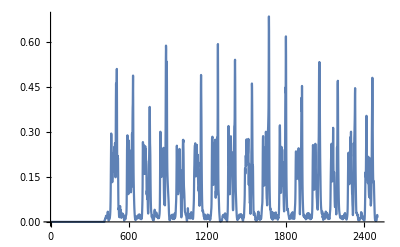

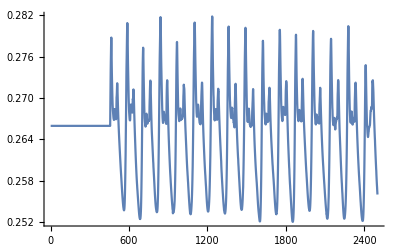

Sub03_(8)walk2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xlsLmtuopt=xxStart time=xxxEnd time=xxx  TA(1) LG(2) MG(3) Sol(4) VL(5) RF(6) VM(7) BF(8) ST(9) GM(10) frametime(0-24.99s)I EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTUI EMGL MTU1.0.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817392.0.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817393.0.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817394.0.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817395.0.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817396.0.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817397.0.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817398.0.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.242817399.0.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173910.0.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173911.0.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173912.0.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173913.0.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173914.0.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173915.0.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173916.0.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173917.0.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173918.0.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173919.0.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173920.0.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173921.0.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173922.0.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173923.0.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173924.0.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173925.0.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173926.0.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173927.0.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173928.0.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173929.0.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173930.0.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173931.0.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173932.0.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173933.0.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173934.0.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173935.0.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173936.0.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173937.0.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173938.0.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173939.0.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173940.0.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173941.0.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173942.0.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173943.0.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173944.0.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173945.0.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173946.0.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173947.0.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173948.0.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173949.0.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173950.0.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173951.0.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173952.0.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173953.0.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173954.0.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173955.0.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173956.0.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173957.0.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173958.0.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173959.0.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173960.0.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173961.0.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173962.0.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173963.0.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173964.0.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173965.0.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173966.0.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173967.0.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173968.0.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173969.0.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173970.0.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173971.0.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173972.0.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173973.0.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173974.0.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173975.0.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173976.0.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173977.0.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173978.0.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173979.0.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173980.0.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173981.0.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173982.0.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173983.0.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173984.0.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173985.0.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173986.0.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173987.0.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173988.0.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173989.0.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173990.0.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173991.0.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173992.0.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173993.0.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173994.0.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173995.0.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173996.0.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173997.0.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173998.0.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.2428173999.0.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739100.0.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739101.1.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739102.1.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739103.1.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739104.1.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739105.1.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739106.1.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739107.1.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739108.1.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739109.1.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739110.1.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739111.1.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739112.1.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739113.1.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739114.1.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739115.1.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739116.1.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739117.1.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739118.1.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739119.1.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739120.1.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739121.1.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739122.1.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739123.1.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739124.1.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739125.1.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739126.1.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739127.1.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739128.1.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739129.1.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739130.1.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739131.1.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739132.1.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739133.1.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739134.1.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739135.1.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739136.1.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739137.1.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739138.1.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739139.1.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739140.1.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739141.1.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739142.1.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739143.1.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739144.1.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739145.1.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739146.1.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739147.1.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739148.1.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739149.1.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739150.1.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739151.1.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739152.1.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739153.1.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739154.1.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739155.1.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739156.1.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739157.1.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739158.1.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739159.1.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739160.1.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739161.1.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739162.1.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739163.1.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739164.1.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739165.1.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739166.1.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739167.1.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739168.1.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739169.1.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739170.1.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739171.1.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739172.1.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739173.1.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739174.1.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739175.1.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739176.1.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739177.1.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739178.1.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739179.1.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739180.1.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739181.1.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739182.1.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739183.1.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739184.1.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739185.1.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739186.1.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739187.1.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739188.1.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739189.1.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739190.1.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739191.1.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739192.1.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739193.1.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739194.1.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739195.1.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739196.1.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739197.1.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739198.1.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739199.1.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739200.1.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739201.2.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739202.2.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739203.2.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739204.2.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739205.2.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739206.2.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739207.2.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739208.2.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739209.2.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739210.2.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739211.2.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739212.2.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739213.2.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739214.2.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739215.2.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739216.2.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739217.2.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739218.2.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739219.2.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739220.2.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739221.2.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739222.2.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739223.2.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739224.2.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739225.2.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739226.2.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739227.2.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739228.2.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739229.2.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739230.2.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739231.2.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739232.2.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739233.2.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739234.2.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739235.2.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739236.2.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739237.2.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739238.2.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739239.2.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739240.2.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739241.2.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739242.2.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739243.2.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739244.2.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739245.2.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739246.2.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739247.2.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739248.2.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739249.2.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739250.2.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739251.2.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739252.2.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739253.2.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739254.2.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739255.2.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739256.2.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739257.2.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739258.2.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739259.2.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739260.2.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739261.2.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739262.2.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739263.2.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739264.2.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739265.2.6400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739266.2.6500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739267.2.6600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739268.2.6700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739269.2.6800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739270.2.6900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739271.2.700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739272.2.7100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739273.2.7200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739274.2.7300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739275.2.7400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739276.2.7500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739277.2.7600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739278.2.7700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739279.2.7800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739280.2.7900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739281.2.800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739282.2.8100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739283.2.8200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739284.2.8300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739285.2.8400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739286.2.8500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739287.2.8600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739288.2.8700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739289.2.8800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739290.2.8900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739291.2.900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739292.2.9100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739293.2.9200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739294.2.9300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739295.2.9400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739296.2.9500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739297.2.9600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739298.2.9700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739299.2.9800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739300.2.9900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739301.3.00.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739302.3.0100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739303.3.0200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739304.3.0300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739305.3.0400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739306.3.0500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739307.3.0600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739308.3.0700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739309.3.0800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739310.3.0900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739311.3.100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739312.3.1100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739313.3.1200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739314.3.1300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739315.3.1400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739316.3.1500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739317.3.1600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739318.3.1700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739319.3.1800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739320.3.1900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739321.3.200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739322.3.2100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739323.3.2200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739324.3.2300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739325.3.2400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739326.3.2500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739327.3.2600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739328.3.2700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739329.3.2800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739330.3.2900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739331.3.300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739332.3.3100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739333.3.3200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739334.3.3300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739335.3.3400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739336.3.3500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739337.3.3600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739338.3.3700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739339.3.3800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739340.3.3900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739341.3.400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739342.3.4100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739343.3.4200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739344.3.4300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739345.3.4400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739346.3.4500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739347.3.4600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739348.3.4700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739349.3.4800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739350.3.4900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739351.3.500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739352.3.5100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739353.3.5200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739354.3.5300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739355.3.5400.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739356.3.5500.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739357.3.5600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739358.3.5700.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739359.3.5800.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739360.3.5900.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739361.3.600.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739362.3.6100.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739363.3.6200.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739364.3.6300.265948600.3824941600.3953237100.2789762600.3052734100.5144893200.2798944900.3937010100.4201535800.24281739365.3.6400.265948600.3824941600.395323710.0022943278834471310.278976260.00165379062468480570.3052734100.5144893200.2798944900.3937010100.4201535800.24281739366.3.6500.265948600.3824941600.395323710.0037794612499786270.278976260.0037194508506653960.3052734100.5144893200.2798944900.3937010100.4201535800.24281739367.3.6600.265948600.3824941600.395323710.0036526249608243520.278976260.0050019933489664590.3052734100.5144893200.2798944900.3937010100.4201535800.24281739368.3.6700.265948600.3824941600.395323710.0021837251607499610.278976260.0052929476716646830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739369.3.6800.26594860.0047188234768997280.382494160.00231120702899105180.395323710.00176815005025827780.278976260.0056142606928445540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739370.3.6900.26594860.0076999893171637110.382494160.00434886176840712950.395323710.00359741806566027480.278976260.0075257523590371320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739371.3.700.26594860.0077901586790308540.382494160.0049173581848955210.395323710.0056463285880445740.278976260.0101804932152871010.3052734100.5144893200.2798944900.3937010100.4201535800.24281739372.3.7100.26594860.0056598273520284450.382494160.00413078105872145660.395323710.0060804762806968950.278976260.0110735285438984930.3052734100.5144893200.2798944900.3937010100.4201535800.24281739373.3.7200.26594860.0041666770936491240.382494160.0036500885936200110.395323710.0050714574478761030.278976260.009632689261775660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739374.3.7300.26594860.0066037683450009990.382494160.00375632637391180940.395323710.00655048696884121850.278976260.0093161060976609530.3052734100.5144893200.2798944900.3937010100.4201535800.24281739375.3.7400.26594860.0087095546293762710.382494160.00339461410888824760.395323710.0091438244367014320.278976260.0130609678843734460.3052734100.5144893200.2798944900.3937010100.4201535800.24281739376.3.7500.26594860.0082839742208928570.382494160.00362570626511131250.395323710.010718137441039510.278976260.020199495743018410.3052734100.5144893200.2798944900.3937010100.4201535800.24281739377.3.7600.26594860.0070197302402144220.382494160.0041906509559225010.395323710.012007808989678640.278976260.026505777890775070.3052734100.5144893200.2798944900.3937010100.4201535800.24281739378.3.7700.26594860.0091478692586979320.382494160.0044391506465160990.395323710.0154953592497694830.278976260.0289716501849881240.3052734100.5144893200.2798944900.3937010100.4201535800.24281739379.3.7800.26594860.0135521043551939820.382494160.00466574088405538250.395323710.0220735435410888070.278976260.0296235992673726180.3052734100.5144893200.2798944900.3937010100.4201535800.24281739380.3.7900.26594860.0182477612969603780.382494160.0056205673274484490.395323710.0324626191180121050.278976260.0325245652876211540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739381.3.800.26594860.022889877067886380.382494160.0064964036651164330.395323710.044909758487159090.278976260.0386838637981769260.3052734100.5144893200.2798944900.3937010100.4201535800.24281739382.3.8100.26594860.0274411230143001770.382494160.0066162376894939960.395323710.0561323785091447440.278976260.0466887864901628440.3052734100.5144893200.2798944900.3937010100.4201535800.24281739383.3.8200.26594860.0309724702848348450.382494160.0074099621374630990.395323710.063556945430903150.278976260.053735702033883880.3052734100.5144893200.2798944900.3937010100.4201535800.24281739384.3.8300.26594860.03340154539025570.382494160.009531650539892030.395323710.065257754911521470.278976260.05703285506472720.3052734100.5144893200.2798944900.3937010100.4201535800.24281739385.3.8400.26594860.0343055589904409440.382494160.0117548923667804270.395323710.060217894439469820.278976260.0576910854260986660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739386.3.8500.26594860.031419182823069140.382494160.0124390473390813380.395323710.049369144122531210.278976260.058135192986176080.3052734100.5144893200.2798944900.3937010100.4201535800.24281739387.3.8600.26594860.024848181957767970.382494160.0109982156029700440.395323710.035772503809206690.278976260.061226494507073670.3052734100.5144893200.2798944900.3937010100.4201535800.24281739388.3.8700.26594860.0171318001270481180.382494160.0080879822071997730.395323710.0231880688721976120.278976260.069197046731683480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739389.3.8800.26594860.0110854417392695650.382494160.004418660264194720.395323710.0149154570953093820.278976260.080277568170514210.3052734100.5144893200.2798944900.3937010100.4201535800.24281739390.3.8900.26594860.0087818401604387070.382494160.00285125009527038620.395323710.0120390182060903190.278976260.090639511723094630.3052734100.5144893200.2798944900.3937010100.4201535800.24281739391.3.900.26594860.0077026771035957050.382494160.002942590006662880.395323710.0128558650428163760.278976260.095761427219817660.3052734100.5144893200.2798944900.3937010100.4201535800.24281739392.3.9100.26594860.0062806074050961350.382494160.0025786558149269210.395323710.0132837934734316170.278976260.093797312182404850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739393.3.9200.26594860.0053490981931110460.382494160.00257559243543464260.395323710.010839086519832650.278976260.08828377340462730.3052734100.5144893200.2798944900.3937010100.4201535800.24281739394.3.9300.26594860.0066244449274489280.382494160.0039414835281170920.395323710.0075093766370955620.278976260.082968864643743670.3052734100.5144893200.2798944900.3937010100.4201535800.24281739395.3.9400.26594860.0091084218180370170.382494160.0059777664380719850.395323710.0071258205836793670.278976260.07966445133741730.3052734100.5144893200.2798944900.3937010100.4201535800.24281739396.3.9500.26594860.0101164259390703790.382494160.0077514775259977830.395323710.0112654812100244740.278976260.073673697139804250.3052734100.5144893200.2798944900.3937010100.4201535800.24281739397.3.9600.26594860.009806463304670240.382494160.008918978565117740.395323710.0194559069644218150.278976260.06037727711045210.3052734100.5144893200.2798944900.3937010100.4201535800.24281739398.3.9700.26594860.0106729856012246110.382494160.0110886685940031010.395323710.0335124213051307750.278976260.045130139681612190.3052734100.5144893200.2798944900.3937010100.4201535800.24281739399.3.9800.26594860.0118469426430138550.382494160.0145690196722839320.395323710.054619446125818160.278976260.033249432106723430.3052734100.5144893200.2798944900.3937010100.4201535800.24281739400.3.9900.26594860.0151484960703194140.382494160.016865208671392040.395323710.068631894581293440.278976260.0252344277283598030.3052734100.5144893200.2798944900.3937010100.4201535800.24281739401.4.00.26594860.022273055611484180.382494160.0186524824013057230.395323710.074242228430455410.278976260.021547873478763360.3052734100.5144893200.2798944900.3937010100.4201535800.24281739402.4.0100.26594860.0255576880878593120.382494160.0176550553878691670.395323710.075251157265768920.278976260.0217222163047463830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739403.4.0200.26594860.021412578294943080.382494160.0129229023335770130.395323710.056893858885545780.278976260.0234571706922533130.3052734100.5144893200.2798944900.3937010100.4201535800.24281739404.4.0300.26594860.0181591788000588470.382494160.0115549346820170360.395323710.034966463710655380.278976260.0223831407527739570.3052734100.5144893200.2798944900.3937010100.4201535800.24281739405.4.0400.26594860.0179411890755280250.382494160.014979721696129660.395323710.0295766791958985250.278976260.0185009361374863340.3052734100.5144893200.2798944900.3937010100.4201535800.24281739406.4.0500.26594860.015213343075863750.382494160.018005831513655040.395323710.027163871472386150.278976260.0155658540825100650.3052734100.5144893200.2798944900.3937010100.4201535800.24281739407.4.0600.26594860.0140408935190854920.382494160.0235494176126138650.395323710.026456615719591420.278976260.0158507963194837560.3052734100.5144893200.2798944900.3937010100.4201535800.24281739408.4.0700.26594860.0155560660493766520.382494160.029963831177695710.395323710.035889874970836110.278976260.020357670531090110.3052734100.5144893200.2798944900.3937010100.4201535800.24281739409.4.0800.26594860.0174380603914809260.382494160.033591923502997830.395323710.048180123753891180.278976260.026745400385939320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739410.4.0900.26594860.019273741913956440.382494160.039418140732269960.395323710.058095292812769160.278976260.0298109138160668860.3052734100.5144893200.2798944900.3937010100.4201535800.24281739411.4.100.26594860.0177688254902899740.382494160.0506006317736478060.395323710.059860606753806520.278976260.0284796754239097540.3052734100.5144893200.2798944900.3937010100.4201535800.24281739412.4.1100.26594860.014791914238442740.382494160.062482722560083960.395323710.061572636609616550.278976260.0269210180699581830.3052734100.5144893200.2798944900.3937010100.4201535800.24281739413.4.120.00316667176564954660.26594860.0168994585727211160.382494160.063668389751596670.395323710.062905993585133820.278976260.0248572556055735480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739414.4.130.005512982245706460.26594860.019090055538408580.382494160.06805262631941250.395323710.064370722195780910.278976260.0184870445669657950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739415.4.140.0068733957611715540.26594860.0158802237210780640.382494160.093552951566433460.395323710.076313890969730170.278976260.0107421905827525980.3052734100.5144893200.2798944900.3937010100.4201535800.24281739416.4.150.0078295810800863910.26594860.0134303143439967450.382494160.149289277436397030.395323710.108364777404805950.278976260.00684429954821678950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739417.4.160.0079933919901270280.26594860.0172496495507631840.382494160.217966505625180380.395323710.13650554908665710.278976260.00609882025045012550.3052734100.5144893200.2798944900.3937010100.4201535800.24281739418.4.170.0083109493214417250.26594860.0163797619081922680.382494160.291520457975498860.395323710.130406960660654350.278976260.00487161423178149740.3052734100.5144893200.2798944900.3937010100.4201535800.24281739419.4.180.0108730832061594350.26594860.015365555323985910.382494160.348234751713514870.395323710.11508835264598070.278976260.00315821344601921550.3052734100.5144893200.2798944900.3937010100.4201535800.24281739420.4.190.0130950312015246860.26594860.0179325866207380480.382494160.35394183542556520.395323710.115124969347777880.278976260.0031406992859440310.3052734100.5144893200.2798944900.3937010100.4201535800.24281739421.4.20.012111517145632910.26594860.0271576160787421470.382494160.377824370701782040.395323710.131635657243748980.278976260.00505477409050419850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739422.4.210.0125979840572015040.26594860.0437262924620016240.382494160.451968199844333560.395323710.156129516717984750.278976260.00707464326863105950.3052734100.5144893200.2798944900.3937010100.4201535800.24281739423.4.220.015964531595478750.26594860.062954857995490530.382494160.43937679073895990.395323710.181134555554967550.278976260.0076908949257310190.3052734100.5144893200.2798944900.3937010100.4201535800.24281739424.4.230.020037205997149980.26594860.085091128737365610.382494160.40256912409988560.395323710.19227102820229970.278976260.006699358489969490.3052734100.5144893200.2798944900.3937010100.4201535800.24281739425.4.240.0202932773477352630.26594860.08628523764831960.382494160.43762011502385590.395323710.178065059425475460.278976260.00561248258698332850.3052734100.5144893200.2798944900.3937010100.4201535800.24281739426.4.250.018855334497724040.26594860.069682247779410110.382494160.48731420116194740.395323710.156344800028782230.278976260.0057902919963724760.3052734100.5144893200.2798944900.3937010100.4201535800.24281739427.4.260.0167241132646407070.26594860.06706944680354390.382494160.4377995160696850.395323710.148678924347132920.278976260.0058191622309029320.3052734100.5144893200.2798944900.3937010100.4201535800.24281739428.4.270.0149593600326314910.26594860.093656602577042670.382494160.363089051266554160.395323710.153102066010490650.278976260.0045240183346969090.3052734100.5144893200.2798944900.3937010100.4201535800.24281739429.4.280.0133441250735658320.26594860.135502406567342280.382494160.40102609638114890.395323710.164289705418759920.278976260.0028438763197566770.3052734100.5144893200.2798944900.3937010100.4201535800.24281739430.4.290.0152632628654666320.26594860.15988902058970720.382494160.50688865029699590.395323710.176622481456232270.278976260.0028082959459899560.3052734100.5144893200.2798944900.3937010100.4201535800.24281739431.4.30.018751969131243280.26594860.148218149294827350.382494160.50353631954575340.395323710.177444934216297840.278976260.0040719757631334220.3052734100.5144893200.2798944900.3937010100.4201535800.24281739432.4.310.0196533582701111030.26594860.11785594601730070.382494160.37934858676742310.395323710.16749229021004680.278976260.0051110587381812120.3052734100.5144893200.2798944900.3937010100.4201535800.24281739433.4.320.0169000358176547120.26594860.103750089659972570.382494160.246554696997238610.395323710.151142228635886940.278976260.0050296346307772150.3052734100.5144893200.2798944900.3937010100.4201535800.24281739434.4.330.0145523370111066040.26594860.103433621374126820.382494160.148235805499303740.395323710.133714045019643980.278976260.0042222867054926410.3052734100.5144893200.2798944900.3937010100.4201535800.24281739435.4.340.0151112831230998980.26594860.095362649658884260.382494160.091501570344746150.395323710.127959032506923950.278976260.0044454403407691420.3052734100.5144893200.2798944900.3937010100.4201535800.24281739436.4.350.020234447660857970.26594860.081832327837979060.382494160.097971927691231720.395323710.134679621803212940.278976260.0060818268442998770.3052734100.5144893200.2798944900.3937010100.4201535800.24281739437.4.360.0300308750833963060.26594860.079906256466135740.382494160.15630417868922860.395323710.161811353390133030.278976260.0072543628961110490.3052734100.5144893200.2798944900.3937010100.4201535800.24281739438.4.370.034001133572179890.26594860.076695661426770230.382494160.198275076100048080.395323710.173079910312491540.278976260.0065931110626185650.3052734100.5144893200.2798944900.3937010100.4201535800.24281739439.4.380.0243434535065565860.26594860.068863000832972990.382494160.192441209814452370.395323710.149649692891068470.278976260.0042401679610581480.3052734100.5144893200.2798944900.3937010100.4201535800.24281739440.4.390.0146884902669951920.26594860.064597848218669670.382494160.169301539891573070.395323710.132889347339083450.278976260.0026520053848575850.305273410.0012796665372453850.5144893200.2798944900.3937010100.4201535800.24281739441.4.40.012404878689674040.26594860.057019096944732280.382494160.12355448191108020.395323710.109343598223505490.278976260.00334855712395673270.305273410.00204234787932377040.5144893200.2798944900.3937010100.4201535800.24281739442.4.410.0090664635778515190.26594860.041863119957424980.382494160.070809622822777830.395323710.069716772672737450.278976260.0043244054711620330.305273410.0030510333549488020.514489320.0048391342062250080.2798944900.3937010100.4201535800.24281739443.4.420.0056716663340259610.26594860.0263507982336249650.382494160.037302271557453710.395323710.040833930482194850.278976260.00347841428737197130.305273410.0037112393291858480.514489320.0077766932694319720.2798944900.3937010100.4201535800.24281739444.4.430.0046552009601519040.26594860.0191391364635438640.382494160.0205896272311659780.395323710.026445274155168310.278976260.00164332823681925850.305273410.0034379128011891620.514489320.0079864746791496730.2798944900.3937010100.4201535800.24281739445.4.440.0049445835156059370.26594860.015895938768649590.382494160.0125826624930321720.395323710.017103253237663440.278976260.001260604005370210.305273410.00257909488723180850.514489320.0069309959327785590.2798944900.3937010100.4201535800.24281739446.4.450.0055849309075453170.26594860.0110000552362554250.382494160.009065101970692150.395323710.0107214423317569820.278976260.00282974027144602180.305273410.0020723144000784020.514489320.0077722449587325590.2798944900.3937010100.4201535800.24281739447.4.460.0065455932294070380.26594860.0066429678751051040.382494160.00639479330997283750.395323710.0064864376816276070.278976260.0039277556967318420.305273410.00208789309369686580.514489320.0098332460270227140.2798944900.3937010100.4201535800.24281739448.4.470.0081061723570586670.26594860.00374188235412362120.382494160.00380276748010632570.395323710.00357696170214486530.278976260.0035773593475619310.305273410.00239901627813451230.514489320.0111795688653516520.2798944900.3937010100.4201535800.24281739449.4.480.0102180635741789330.26594860.00366878787523566970.382494160.00282466568570210060.395323710.00173604309654778760.278976260.00240371753557814230.305273410.00206758516953947260.514489320.009840616346337310.2798944900.3937010100.4201535800.24281739450.4.490.0116335582251648790.26594860.0051428850114952630.382494160.00383486439572616570.395323710.00173155483040338230.278976260.0021410140020670550.305273410.00245092845208485020.514489320.0062182025261276930.2798944900.3937010100.4201535800.24281739451.4.50.0116416258629679970.26594860.0053772056691488180.382494160.0046615289392638980.395323710.00284733680588590420.278976260.00320209822547092540.305273410.0031306654619918550.514489320.00355792335993010240.2798944900.3937010100.4201535800.24281739452.4.510.0111196021287221170.26594860.0037688585678473010.382494160.00373143315046910560.395323710.0028472391115790020.278976260.0039571272853827820.305273410.00320733261773561160.514489320.0045353093791510310.2798944900.3937010100.4201535800.24281739453.4.520.012928513167820410.26594860.0028215029611183880.382494160.00247331786496281670.395323710.0021300580840721120.278976260.0035417540279739270.305273410.00277163271674142660.514489320.0067739195066058020.2798944900.393701010.00086287211820664030.4201535800.24281739454.4.530.0162440060850731930.26594860.004381099009700110.382494160.002793558154072240.395323710.00201273484231613130.278976260.002670605675722070.305273410.00203414376282331140.514489320.0069370345544343060.2798944900.393701010.00180555246099891940.4201535800.24281739455.4.540.0200412711663705940.26594860.0062472714311629220.382494160.0041387413394397860.395323710.00340925673283987930.278976260.0024579504771124180.305273410.00155927602753831150.514489320.00525740417490238450.2798944900.393701010.00189199740990255880.4201535800.24281739456.4.550.025400453361838830.26594860.0061910506412480730.382494160.00483186663646664650.395323710.0052648926589105860.278976260.00370385856150339540.305273410.00161875798958891250.514489320.0053260972348596380.2798944900.393701010.00144750728616814470.4201535800.24281739457.4.560.0334468239187651550.26803520.0045424155616329630.382494160.00431082814851528950.395323710.0061511128552816210.276856060.0050032077436165490.305273410.00224542619088392070.514489320.0076853138045770070.2798944900.393701010.00167495815775843640.4201535800.24281739458.4.570.046404293371854720.270084550.0043753177651667320.382494160.00360869341680637770.395323710.0060660087018040320.274708190.0048226240621536790.305273410.00274445837434089720.514489320.0096467008963444670.2798944900.393701010.0031570433967776710.4201535800.24281739459.4.580.067447383945923760.27197530.0067568908006633810.382494160.0042857274298659590.395323710.0066280151188228790.272668410.0030903354544871710.305273410.00366530879778157160.514489320.0092938500015408780.2798944900.393701010.0045469943177064690.4201535800.24281739460.4.590.102670675622800020.273894350.0102070703190749890.382494160.0059638696834001270.395323710.0088954766191837440.270540630.002071613104042370.305273410.004911929925169440.514489320.0075055895400503520.2798944900.393701010.00510615535314331340.4201535800.24281739461.4.60.154744705291527530.275218860.0124076243132686720.382494160.0067789151454773190.395323710.011187461170443170.269038090.0031060523579756470.305273410.0064688500828062330.514489320.0069886453360927530.2798944900.393701010.00495097920784254640.4201535800.24281739462.4.610.203277023908750520.276329440.0131894699443771480.382494160.0062988443798521440.395323710.0117823361171200320.267756780.0046146581080212520.305273410.0083029197291230390.514489320.008300399856696150.2798944900.393701010.0045432456407067150.4201535800.24281739463.4.620.247466755065586940.27757430.0151050375280348880.382494160.0052154400785908440.395323710.01089682806488070.266297240.0044433512035952830.305273410.0101881060405104270.514489320.0092166112004644020.2798944900.393701010.0047806297325857180.4201535800.24281739464.4.630.29408747161575770.278579590.0196763123888634570.382494160.0049198508746639790.395323710.0098184361525834730.26510060.0026737120182607120.305273410.0119749934938105270.514489320.0083237894238674960.2798944900.393701010.0055049938929389430.4201535800.24281739465.4.640.28860168667353980.278744820.0236329212765530520.382494160.0051553557922724930.395323710.0093726834639312350.264902380.00194262498386131770.305273410.013364066001820830.514489320.0057537114205953620.2798944900.393701010.0053742385560791660.4201535800.24281739466.4.650.241118445665026220.27781270.0227251306668778650.382494160.0045902620426633540.395323710.0090530828497933940.266014920.00337399446730662430.305273410.0142561565709720550.514489320.0046166885167789270.2798944900.393701010.0039902874105271950.4201535800.24281739467.4.660.198964570028063340.276276380.0176687947451336470.382494160.00317548421915738770.395323710.0081856727232279430.267818450.0048633694297948120.305273410.0154305380948785660.514489320.0073060200768117630.2798944900.393701010.00275386627108378320.4201535800.24281739468.4.670.192843035902184380.274802150.0128934081574361170.382494160.00198053160340518060.395323710.0065429854698947570.269513810.0045156193591977540.305273410.0161442837797679780.514489320.0095070450989195480.2798944900.393701010.00281306461978063970.4201535800.24281739469.4.680.190099379251270960.273564410.011500147424023080.382494160.00207868661927516650.395323710.0055732898562777880.27091060.002380839585687880.305273410.0152087866610823040.514489320.0081101262779286390.2798944900.393701010.0031916738802733680.4201535800.24281739470.4.690.167383910898257830.272572050.0121856533399968530.382494160.00354148817422871760.395323710.0065569148210108360.272012990.00137318324160358550.305273410.0127511872456571780.514489320.0052628459281489880.2798944900.393701010.00291188412352352340.4201535800.24281739471.4.70.140214657585372130.271740190.011447678608065070.382494160.0047921639914392270.395323710.0072480849522729230.272925110.00277863245632656040.305273410.0098688021753350450.514489320.0047085998170278310.2798944900.393701010.00177676876769709570.4201535800.24281739472.4.710.132061195882630020.270929190.0091707463917779730.382494160.0050758740395300250.395323710.006202037303298790.27380390.0038361960354597440.305273410.0078222401979203010.514489320.0061609712813771680.2798944900.393701010.0008958315846278220.4201535800.24281739473.4.720.13904278441200260.270145890.0074085101905531690.382494160.0056191119477096690.395323710.0044888568513234020.27464290.00309371143192703740.305273410.00682379595012279350.514489320.0067812314873619120.2798944900.393701010.00125484238471847270.420153580.00211762834066460660.24281739474.4.730.145073624762718960.269461850.008112709750748290.382494160.0079616488663593870.395323710.00454558836298237650.275367730.00175376929813558880.305273410.0060702930627419170.514489320.0061677393095946520.2798944900.393701010.00215419075965315140.420153580.00598769071759790250.24281739475.4.740.162822067925414230.268915520.0096149518983093640.382494160.0118340912037098650.395323710.0067677229140331290.275941420.00211874115392868050.305273410.00535236791242526140.514489320.0042222026745603130.2798944900.393701010.00238035483588547440.420153580.0085978180447587960.24281739476.4.750.20625991248009410.268501540.0094482494618379730.382494160.0153541078519879620.395323710.0092496849762771560.276373030.0033615236310801290.305273410.0046884678579916920.514489320.0029368993196148340.2798944900.393701010.0015688763761113750.420153580.0074424426932258760.24396839477.4.760.228782491663933360.268187670.007446608699471640.382494160.018905037173966440.395323710.0103729854445988120.27669850.0041529521226788160.305273410.0039543675184733550.514489320.0046981372976272610.279894490.0035737991253595370.393701010.00094229081135532830.420153580.0050433959124291780.24508009478.4.770.223552111854401440.267925890.0052755899871064410.382494160.0279555679338895950.395323710.0101268496492582050.276968790.0036690313757687710.305273410.0033727121693382520.514489320.007387102530262830.279894490.0082343214021634960.393701010.00172135789081952470.420153580.0046845305709454230.24616998479.4.780.20473506505536360.267681780.005141779851126870.382494160.046759939834388210.395323710.0101661951083742260.277219890.0022642425351390110.305273410.00344325031214946870.514489320.0076791866278660760.279894490.0106009711814938350.393701010.0028025321688932430.420153580.0070556692670479170.24726155480.4.790.171171537634513480.26741990.0060348168977685310.382494160.06508263513707490.395323710.0129413151048378030.277488230.00220362165411644350.305273410.0040956309024298470.514489320.0056268881341938830.279894490.009778549006086830.393701010.00288525220932056220.420153580.0083452891962185440.24827409481.4.80.166768695607718680.267194420.0060124046364015720.382494160.066289222573307150.395323710.0172196659015928020.277718440.00366357242519357120.305273410.0046810466040595350.514489320.0043811482342175140.279894490.007318816158694330.395723020.0021023938335731150.420153580.0072618836990359450.24923417482.4.810.187801625316084440.267021590.0049492140878619140.382494160.054963744586106270.395323710.0204552756254776230.277894350.0045690593165938250.305273410.0049280705744092320.514489320.0057515039639020980.279894490.0064853522819831420.39783830.00189812313243362030.420153580.00523174420934910750.25013015483.4.820.203251440191436620.266988390.00560106374471630.382494160.061085517184768680.395323710.023910392822805710.277928090.00392153959696849450.305273410.0044043605831730820.514489320.0081463091546905650.279894490.0088572628131899750.399879730.00284793003060485350.420153580.005447811262377450.25085747484.4.830.204248879670996720.266863490.0097225837717158610.382494160.084667276499459930.395323710.028437609755270240.278054880.00229192917529156240.305273410.00306016162078452760.514489320.007907935737747920.279894490.01084033762687270.402156330.004063131097631270.423225520.0079420071734925040.25163165485.4.840.223359376768139130.266798890.0128147962445933250.382494160.098160282343780530.395323710.035261770932803510.278120360.00147485272267905460.305273410.00197349983187195640.514489320.00494490008421694450.279894490.009799479843776610.404450860.00558800615585163750.426369630.0097199709185378240.25232328486.4.850.242197868797661670.266871690.0113672574475982250.382494160.097850106263290850.395323710.0442346205657498660.278046570.0028550202922205090.305273410.0020863983009714630.511814910.00347643031730647270.279894490.00757102156802861360.406792270.0089243242365734040.429609870.0092570711541246730.25296357487.4.860.24324960998804510.267108110.0070945288817550050.382494160.086287035909817460.395323710.0524717263308010.277806340.0045481113681411930.305273410.0031319983843478030.50906590.0060062128986890520.279894490.00954000005038430.409168490.0157413331056067520.432925880.00746146199121621840.25355227488.4.870.222219048037618550.267490790.00335563867019640550.382494160.066420640927448270.395323710.0504624097029770440.27741570.0054755067620821140.305273410.0042815759415893190.506230440.0086290834138500470.279894490.0158987260634204930.411574050.026417615026650160.436294880.0069336955153858410.25410621489.4.880.24066786788463210.267921550.00290962643618577830.382494160.041586235111950930.395323710.036616662511580520.276973270.0062063031697332810.305273410.0054413401917247390.50332140.0086259450413659620.279894490.020300071526471890.413965550.0410775226528125040.439651790.010520395979086320.25460825490.4.890.25102791577421230.268228990.0043196543334686480.382494160.0268926441325287170.395323710.022230849047389290.276655740.0079033739602026070.305273410.0061081351602023390.500363250.0070671158225888840.279894490.0241113562223473530.416356590.05352991176889250.442968540.0143544724755184220.25513244491.4.90.207483918406353160.268358690.0071180339986139590.382494160.0192047455130252320.395323710.0148401036673599560.276521350.0100844826332238820.305273410.006763298470521030.497467730.0073953973451449180.279894490.034398801354055180.418682690.055901440369892040.446144260.0142395101203115770.25567822492.4.910.227959894519373980.268278360.0096383230656247370.382494160.0125568216871588120.395323710.0122723964213338650.276604620.011678575167772850.305273410.0076212080775332650.49473130.009857597831863760.279894490.0440231857676239850.420891930.0601105422873281850.449099020.011490598682010340.25625159493.4.920.26197832822963630.268340540.0093302323419452520.382494160.0075594727341006150.395323710.0108511717781841450.276540170.0128795738652268640.303182720.0090713876241350150.492205170.0128504795152385440.277954290.045579560054623010.4229590.064143895821704220.451794050.0131535433545811150.25688213494.4.930.249113260145889940.268166150.0079475182794371290.382494160.0046329537785665880.395323710.0090277135080754580.276720760.0147210190910412940.301405750.0115089928898663240.490022090.0150897944542185050.27630330.0495749384619732360.424766690.059641037422781740.454098430.0230880231115724030.25749164495.4.940.22289749190064190.26790060.0079876535078681580.382494160.00389917272536959360.395323710.0078835128325432550.276994850.0190379595088971640.299911160.0144007492894144050.488181820.015501804842791490.274910050.052530727903311690.426293450.0545333315185407840.456009890.039672377327024530.25805255496.4.950.175393796279921660.267646390.0072935930011219140.382494160.0039202597165283230.395323710.0079718747564267720.277256220.0263864892741077770.29865440.0173977311497153580.486670560.015669827199190990.273733220.052021614683617710.427534160.04857573920717990.457545420.059481392074726510.25854135497.4.960.148447780317690130.267474010.0055318835743132330.383187020.0043440429815178870.395323710.0092837886700939590.277432880.035391100273789560.297609280.0200827640637503860.485499920.0180763670331508460.272749780.0494608609629085050.428475390.0343110203155304260.458701580.082151343593417080.25896539498.4.970.211756989557862680.26728670.0058894020621826910.383747470.005165810731587760.395323710.0121797543927287550.277624320.044059779767301320.296863380.021938953931704560.484718590.023811728687309130.272044740.0452655878122755350.429104890.0211838797683895460.459462630.107634975982161940.25929847499.4.980.320520390092214340.267120290.0098918229200080050.384076950.006618133248957930.395323710.0169900173543433360.277793950.052643389867355220.296400370.023992956889355650.48434390.03420335100266950.271605610.040193540616487830.429417660.0142281213125964160.459813470.133791225437578760.25959339500.4.990.41250889879938090.266908320.0131160311155977760.384345980.0078002307871042180.395569030.0219816132907744360.278009410.0655065830789660.296241710.0260136654196063620.484366670.0495434992648196360.271454840.0338388923772788360.429396210.0101468984912202690.459757320.15512731675710850.25976164501.5.0.46026068449977130.266909720.0135782126088022230.384296860.0079525761416750320.395541310.0256645958663268450.278007980.084722100992709950.296420170.026739117329732420.484710370.067783014804739130.271624410.0271516806673470360.429138510.0071806456327939510.459396080.16460195245069460.25988463502.5.010.433969156387848330.266981520.0142058586146961830.384099510.008746767842633540.395407850.0301792147809200570.277935070.108548627314387110.29680910.0280053129309376020.485371210.081210734260102270.271993320.0236123091176776160.428604520.0054982329595754520.458700490.159481583504946180.25990129503.5.020.40121526102983590.26734760.0187497528229649270.383357350.010756485246763560.394910480.037580740433827810.277562130.132282118257915250.29753710.032679571109950920.486449730.083246432435237940.272681670.025390461517159760.427765830.0055949966617786520.457602870.142441984461882410.25988136504.5.030.411735661366863240.268913880.0260309632736141320.381273730.0133524863213324850.393118710.045087565955679650.275943130.148200827463539740.298344950.0367127421390960540.487542370.073963854971157640.273442520.0303575368294722870.426916780.007258790440702690.456482760.119184195660951940.25989106505.5.040.41121958189704080.270091880.0312107321913891180.379445820.018034409225145880.391662730.050102856776384270.274700390.150840809887446640.299439460.037472573945550130.488793040.059054604393630660.2744690.0358117821060761550.426077610.0095727982697347750.45527330.095684325088210730.26019928506.5.050.46734638351823830.27027330.033732953602992940.378457770.024838728827172680.391168890.054351583752849950.274507080.139179676880897380.301022580.039107311789691490.490517890.0472945107610959550.275946630.040767158807931020.424991330.0116346964570730790.453631480.076084350511963440.26078779507.5.060.50900350127890060.270657080.0335097970688850240.377244870.0281809442217292420.390434950.054381940143999830.274096440.119234303831811440.302575610.040911953928012230.49224290.042281886367115010.277390650.045204556106132660.423853430.0126549796935177050.451918820.061165262670340880.26135065508.5.070.39837135071260110.271310260.0286163253529288130.375943480.0243456572130470940.38947840.045665045867441710.273392260.104768595132455650.303687660.036524282508789290.493653710.0381556283639264550.278422890.048093368978230010.422776840.0127857667441809810.450405490.04832810063500250.2615792509.5.080.25458665149655880.271952960.021365160245506920.374820710.0161361029792268660.388596880.031455554956685630.272692850.104151722219215090.304456850.0289255613807933470.494860640.034688055179390460.279136620.048905502716725590.4217010.012580076134507370.449016270.0367033630460634340.26144975510.5.090.18238424904458540.272124270.0162445752124779630.374288730.0090922346184893160.388123780.0195337497031855130.272505330.106606185701799890.305099660.024041048327447050.495999450.034929006683962850.27973320.0469294152520965960.420571020.0120564072933831160.44764780.0278704773658269360.26099583511.5.10.169962076499387720.271754690.0136284673146370270.374387880.0066591042779001460.388238730.0149419676467446250.272909310.10134267653825990.305695130.0215997818476260720.49718980.038410477461393530.28028610.0416946821979142860.419300770.0104455112884040810.446166310.022762880540627040.26031205512.5.110.195350265372126020.271202490.010644184360030880.37474010.0070093112631325260.388596710.0133787850761983760.273508910.08842077752552730.306191520.0207692285057388820.498458860.042904537108926080.28074730.034149482467608350.417862390.0073635844957092050.444527710.0208561159413626840.25949873513.5.120.219880897335660550.270528370.0078672653013777870.375288810.0067327942354018330.3891430.0108856159714931530.274234420.072268197915560770.306564480.022322073733178480.499733820.046961526529726160.281094050.0266328907865423760.416343410.0047583076894257250.442829660.0245935617419820970.25861673514.5.130.204886498760188580.269825410.0063300940426597360.375926250.00480772275098260550.389773230.0074149290223607350.27498340.061012134024435920.306820630.028155143506503340.500961930.0494566416956446350.281332330.0213319610876482460.414814590.003973721477515520.441142650.0340769462714307640.25774168515.5.140.20997097740654630.269149360.0069171014127155590.376579890.00332025918578062040.390417450.00558186905442619240.275696440.058418967627451150.306981340.035319881566778490.502069870.0497336230660785640.281481870.0170768924636142340.41336670.0044147228373678410.439570710.045695015177007320.256884516.5.150.211697296880836380.268527370.0080029052743367960.377216440.0042164406273437670.391043350.0058895153583033930.276346180.059837077487793690.307055540.0370441202166229560.503017150.048309752357925550.281550940.0119310661159960190.412058840.0045985693822784530.438178420.055654493483242510.25606199517.5.160.15845171970306890.267923010.0071914744383992090.377850080.0050908475978400560.391665970.0063157183083889040.276971770.0622352103195164260.30709170.031432705162607110.503816150.046238556845404080.281584590.0068647662505988090.410920710.0048224301214698120.436982060.061978909112224650.2553089518.5.170.098749042475084740.267364310.00464996298126470540.37844540.0038988193137360430.392250740.0057214723805978590.277545060.063230176117264360.307100430.0211237013715383540.504514340.0439043809610072250.281592720.0063715803929477510.409899680.0071478117097770810.435919270.064782165806122140.25461213519.5.180.0582364239740773560.266827680.0030900611647546840.379025260.00223424517530638940.392820160.005727771323339420.278091190.066067510699250540.307087610.0132845853706373330.505142120.0413783260213374040.281580780.0095735411058284010.408959170.0128252246520028130.434952780.066027889270256020.25393095520.5.190.0413653523809550260.266314640.00462943610295343550.379595730.00242313282486386960.393379870.0073353020353284110.278609160.07674852683235440.307039830.0134246063981810650.505689920.0397061131307530550.281536310.0111008488715043060.408101640.0210757355637446670.434091740.066437980707865660.25324692521.5.20.0457930062876716750.265831320.0057165667946648260.380158530.00335763818545895550.39393110.0087202110288412490.279093440.084042436076100620.306942880.0180329721020844570.506159440.0396719837313056840.281446080.0096482682154632110.407312830.031190402366575610.433324140.067338296026410920.25255311522.5.210.042973747187992870.265364390.0044824820184867070.380720050.0041538450840100650.394480390.0090803240877339650.279557910.077221262737655730.306811410.019854757426807820.506561570.0401613255127369340.281323750.0084486421269010290.406591160.042308521657155020.43264130.071718806515561670.25186708523.5.220.0293195693161129870.264930780.002075818072083260.38125850.0039236574012595680.39500640.0092147609470539570.279986250.06368907033642090.306653360.017809757868808090.506918280.039491536129342140.281176720.0102960789538669960.405914540.0531639440863741560.432016660.082270472025298970.25117983524.5.230.019693770181587360.264512210.00044144561242953690.381787360.0020635663692860160.395522590.0097101126805166050.280397040.050671119030728370.306479650.0152287771049189210.507232770.034744736424844210.281015160.013026187572883460.405284630.06212757905882070.431449810.09767708916563350.25049213525.5.240.0166776119577687130.264107520.00147947806078530280.38229960.0021736683394621450.396022440.0125904753976904160.280791660.035348708350426440.306305740.0119933248429642660.507548910.0255160192654976660.280853470.0135854209086037380.404659050.067474383742630840.430887920.11244540784105290.24979642526.5.250.0169537896401586070.263721860.00352920474111385360.382796570.0060913691541325640.396506880.020528136262692520.281165430.0198438507416278940.306119760.008012321226000570.507892430.0156730233681964120.280680610.0114859833409334240.403994650.067912264703113390.430289780.120176955016007810.24905295527.5.260.0164526716901708740.263338980.00567882021457075550.383290280.0125635874815654590.396987990.038962798071106790.281534280.0110254694773501730.305930650.00510259134785000750.508245070.0101008873533458050.280504880.0083982205189039980.403322550.063755957561422270.429686820.116751073745156140.24827875528.5.270.0152966705911056450.262961430.0081188413784663570.383778390.0227828103760817050.397463420.065303351430913770.281895830.0096387385807802480.305737980.0055260534519700430.508614720.0110672808625131970.28032590.00654642499009404360.402634450.057153149904716770.429067550.103059190279718290.24748186529.5.280.0183324919620525650.262588160.0116958863919679730.384260750.036748684378707690.397933090.081686789887723860.282251180.0126889471693377250.305544170.0084874092144835710.509003690.0142640100192576810.28014590.0064544554378147110.401922610.051042658728111130.428425480.084525147275969340.246651530.5.290.0310822520748361730.262214060.0153276137147034060.384738790.0528177671133252260.398398630.075432417857193460.282605220.018911688541469640.305356350.010242374966206030.509406020.0157903214819787170.279971490.0067165296521863030.40120180.046712767778095550.42777240.068720396405947930.24580798531.5.30.047384661977788650.261847940.019452826053564860.385204720.069378553274270690.398852350.0598374801678463260.282949680.024967775063986720.305172490.0108290537509139260.50981090.016919961865845220.27980080.006293036254742770.400484420.043245546757226360.42712190.059874396362711860.24496213532.5.310.0526373847292925450.261477330.0232233417069746960.385672880.079127825924673770.399308270.054564786945805610.283296330.0268751570566474160.304989310.0129382893330732520.510208190.01719103032393980.279630770.0057906842722345290.399777360.039020653352140610.426483780.0549623336348190540.24411185533.5.320.043237022496917860.26112220.0213925577860331930.386126930.081566116369788080.399749950.044142087601900960.283626590.0261544694726224650.304800080.017130622855608590.51057420.0146840655851220550.279455140.0063000294221402150.399106190.0333907962985050750.425885880.049046317596668510.24327891534.5.330.028600784373479470.260766990.016845444908859650.386575840.104515661741432760.400186750.041200396372917750.283955040.0232953649631638880.304617340.0206518100361556860.510929910.0110049421986930010.279285540.0077448339982772280.398458030.0269597440719686020.425308640.0407088537133047240.2424688535.5.340.0191462778277051750.260406650.015763671253911030.387033020.17222206718663870.400598330.053309483524825890.284286330.017589233265016760.304425070.020015495967262290.511269030.0077630301084837980.279107120.0084063931214195720.397815310.020412903394454840.424744520.031754447682247690.24163698536.5.350.0255467746087867380.260061220.0185200118534711540.387477560.27762176184963520.400981460.073641943383286240.284602110.011295557355838150.304225480.0150839366186497140.511590820.0041375630703302380.278921930.0063825026339706950.39718660.0141657955602878540.424197070.0231787715364521160.24081261537.5.360.0395236364851177040.259719530.0224441413665292870.387919360.36950059628122610.40136040.103296729643455760.284912740.0075342114945368050.304020790.0098513012962473230.511906490.00283868821847509070.2787320.0045596120390620480.396558010.0087675298299773970.423650310.015222059155858110.2399897538.5.370.036642765817753420.259390380.0266628258805897930.388349030.403758535307617460.401726250.121869408158647320.285210350.006639913468503980.303812710.0070382894832428530.512212150.0060747095041287210.278538920.0059731904125692260.395933990.0050162967442081640.423108540.00889134789265930.23917323539.5.380.022620130173944570.259072860.0314426062652762850.388762230.400120005237114050.402077730.117526675928999010.285495940.0068510580115198250.303611480.006129474631179650.512515650.0094981347293745160.278352190.0081027543169643660.395312790.0036911457562825310.422565550.0060048005004348880.23837504540.5.390.0143134733166026450.258760530.0314375054572152840.389167930.36099203269282780.402422260.100935242550433540.285775420.0091443551148890430.303412150.0067868876253809050.512810930.0100231993012568440.278167220.0085491778769716430.394696970.0040398877059900140.422026330.0066100629285325110.23759114541.5.40.0142781305495736260.258449830.0255413687441873040.389566480.292324660884587030.402761990.0906533035385410.286052030.0142888466912669660.303220840.0075865036449186470.513097020.0073299578058782880.277989680.006774890299407050.394094410.0044056805182320720.421497690.0079513105597920130.23682678542.5.410.0196468839113904950.25813860.0218335538389497520.389959160.28008724214280870.403098660.116650174215010780.28632770.020047014693210650.303039160.0064924407217920440.513376040.004258656368808230.277821030.0042936612794068590.393503760.0044096842046719640.420977380.0075231966063611670.23608461543.5.420.0203608808620168130.257818090.0265983771669470040.390357420.354669040041860950.403441930.157316164359048020.286610120.0221859166824306780.302861160.0042365369283896260.513652370.0050416776334985980.27765580.0039789122235759960.392916120.0047521187971946310.420458440.00541461667028583960.23534998544.5.430.0160304915176682460.257490150.04228019339823370.390762080.39425420507302620.403790550.162791815378560440.286897550.0181545898715675980.302681670.00340084087853549960.513926930.0071695267303973380.277489140.0058840158124497120.392327810.0065530569617127830.419938910.0051913893183483040.23461354545.5.440.015220896728523780.257175290.064504666341047230.39115640.376222536561276970.404127350.134375438484228640.287172050.0115689568845141620.302495240.00349897648319180040.514197440.0079384179502543850.277316020.0075902988568777370.391735860.0098786883600838590.41941850.0084889106075734430.23386335546.5.450.019426925410828450.256858250.087619790638816960.3915510.36380592439378160.404465250.120830974647465780.287447020.0061305687770206340.302309520.0026421645386218340.514482160.0058486406227407440.27714350.0062917613062137050.391126960.0141493275623119940.418879490.0097217709932097450.23309959547.5.460.024018357632985520.256552230.103471808919012590.391931660.415773426377686160.404789880.13726816838369740.287711040.0045236498111443810.302128070.00188071140392632830.514776520.00325346363469420070.276974920.0038880786687857750.390509020.0195318251663968230.418330570.00722386179626737650.2323215548.5.470.0269664294444412270.25625460.102989972173368780.392301250.50539301126655940.405104570.164152358173948080.287966550.0051632176923013080.301950290.00203597778325822960.51506320.00455173878436934250.27680970.0045768960862236010.389906030.0259897265636194580.417797210.0043596056962160570.23154327549.5.480.027219293656034290.255968120.089331092991172170.392659070.55492163615486090.405407680.184391251055482990.288211280.00444769448803983450.301772750.00233204007592532950.515332840.00728755857037461950.276644650.0079649627894166470.389329950.032257726480131830.417291570.0041551294759707210.23077836550.5.490.0281761879328865440.255696870.082943422993060070.39300060.58678510167824470.405695050.20006780533262630.288441930.00306737395879749230.30159710.00238135372442281660.515577920.0072636406743912740.276481310.0093430861577512410.388790570.03665990033592190.416823270.0064118568989780410.23003741551.5.50.02567607635423280.255426640.085352755459289410.393332070.58685199838769190.405977110.210854407444153570.288670670.00311556423425912370.301437420.0022505074049535710.515802350.0049432819031669180.276332770.0074607135734166260.388302410.037836384570353250.41639710.0083243486397845830.22937623552.5.510.0221656694784339270.255176140.091968560148787560.393656350.53225807205722430.40624470.224558869437491040.288881780.0041257445300268560.301253790.0027743277324755040.515999920.00382779847576677570.276161890.0053661062131042040.387819810.035613844702640110.415992290.0078314410629853940.22864886553.5.520.020115386581389540.254933560.105491848759891950.393960640.45753908543466250.406499410.234626446950251670.289085370.0043481152605555790.301093550.0037774618644764020.516188980.0050995022964178620.276012720.00584318241983336740.387375760.0310767653779318660.41561490.0055716509254895540.22799524554.5.530.0190317173062332020.254702640.113822867724314460.394249030.393418329184146930.406740840.21213623152729710.289278390.00348594866659740440.300942010.00402409734371690.516375340.0067224211861700060.275871590.0084850052064676210.386944470.0256919932188260850.415247590.0050946197136339660.227356555.5.540.0215216125755742540.254495080.117628297783810220.394509480.357847606433802370.406957890.173030355580181480.289451260.00260462402962208150.300802010.00315760385476588370.516565960.00696130547586870.275741160.0094678382408392960.386519110.0206611158281154660.414882430.0081663109116060850.22672852556.5.550.0245660121052408660.254306940.123695390397757830.39473290.3309729685611210.407149410.152666378657021070.289607420.00313723938196108340.300699340.00196116105133041640.516786750.0057307049250923240.275645490.0073112459836722020.386088660.016211237245324230.414499520.0101863886280072120.2261297557.5.560.0234486317483064320.254140480.1281498325920950.394939520.265371229346485050.407322030.157026667160636240.289745180.004967207893893650.300589820.00157569342256781620.517017240.0041227576929311370.275543390.0042807814117456350.385637090.0118450963443302510.414102520.0081016861968363430.22546834558.5.570.018923852379318740.254034570.128851576783753670.395062030.185035391228674850.407428350.194341356925376350.289832630.0065612515601395830.300537640.002092234851143470.517230480.00534629480773268950.275494750.0033144472560714210.385273790.0079375047337928440.413773390.0043370960731392360.22494935559.5.580.0195406766997091070.253882320.133940654091081220.395200140.133557976863394740.407566460.23616600694375520.289958060.0063453265166412490.300538350.00234375501930713130.517589640.0076265125968832070.275495410.0058757514878306420.384737090.0052513971750212560.413265930.00306676653058813140.22423303560.5.590.0193474491422070680.253869170.12105404368894120.3951780.109323795072406180.407565340.230977362371442650.289968870.0043201078690593150.300606660.00170310186031698960.517927250.007340544581494230.275559090.0081427193168752640.384311680.00375652756883135050.412841430.00442875228126726750.22372159561.5.60.0141376539290408930.253715790.092678795949792880.395282180.088540673492638710.407690910.212824719130936230.290094880.0028599524495686010.300676780.00067484279130463990.518353660.0040512497133516110.275624460.0066383507199689670.383735410.00247839537779357720.412284840.0058859045454671440.22294077562.5.610.008347287781752380.253760280.070024770414217380.395175380.067893364358628790.407624970.18321942845660530.290058360.00291022318079221540.300809670.0005940315084726630.518737790.00202271579447835730.27574830.0029183280343416740.383320380.00110092810743442090.411855550.0055144418263719730.22244692563.5.620.00468013753088296350.253732450.054236559781512390.395118540.0476890981986365860.407618290.139323589681671770.290081210.00340673127721971430.300973510.00184758239464395350.519227830.0052346894701448530.275900930.00135641475368740420.382738230.00036981851206194040.411260360.00373221479536009740.22176948564.5.630.0075537585256834250.253859390.0565494991504431750.394909590.0363669411075702860.407466580.104661292957520950.289976920.0035956535591966870.30116020.00277996664376874840.519647020.0094786852161519650.276074770.00410195375075830.382343570.00096227881648183180.410837590.0038514730470016250.22131236565.5.640.0137071046827611080.254026610.065195380468748050.394650310.0358925661423882550.407272450.091987116074436960.289839190.00281837715358921850.301373190.00225092709686348840.519997360.010201463652084340.2762730.0079100190140099090.382021620.002027443176066750.410479840.00731901505671145050.22096709566.5.650.0182604961475586780.254355220.063654037016767880.394215670.03762807121295060.406919490.096491447226558430.28956740.00161401052526993750.301640330.00103467185516674320.520267480.0079164738803446550.276521520.0094468081927198510.381928380.00261235487798033160.410326540.0103169215969134420.2209038567.5.660.0191173689142369630.254795970.055104576456202630.393659790.0359229087173142040.406455160.102832135568293530.289200470.0021019141522169450.301940050.00086168669156351790.520631590.0061947897616031940.276800180.0079153350564378240.381735880.002428996892683220.410070020.0111563958814174580.22072897568.5.670.0165316653621101520.255402440.042245324041802520.392924050.0272886316739706540.405825290.085751236244908920.288691090.003441872873301410.302286130.00153147781755098550.521051310.0072152896140430590.277121770.0057093650791210130.381496520.00161075559973445780.409772920.0085249668847854170.22039042569.5.680.0112470609594590340.256134450.0264398962341039140.392041330.017815981677789280.405063270.0532510570614608060.288069330.0039219127843942430.302680160.00205638517640132760.52157420.0094815382585104640.277487740.0068890644223021440.381133770.00125442283780900670.409354670.0050435864904851050.2198474570.5.690.008897890486194670.257027220.0132419290516653920.390960340.011507773010240590.404126030.0304345624420840070.287300640.0030307994999367730.303149940.00203430919348365330.522238620.0101288528586037040.277923870.0096064783830539760.380619190.00186723155861940620.408768460.0061845862326534350.21916751571.5.70.0101290360222285450.258060420.0066830346652054550.389663260.008353016166033180.403013810.023166789776074130.286396730.00149553194513021330.303755820.00165461683802995510.523007060.0081211456215067160.278486130.0098388131192941230.380070810.00235052600002396470.408100870.0090327932005893910.21858551572.5.710.0110691024918116630.259150380.0054126943133056740.388191680.00747226382651491450.401785040.0230977451024308830.285426350.00074523855226479820.304559790.00157402119577941930.52393470.0045199527473160750.279232140.007038992925047940.379466220.00203985943028025260.407300670.0090911469350226340.21817949573.5.720.010389330110780630.260558220.0057576974498717980.386328670.007924624261766220.399975480.0212602420448560860.284147220.00156325301528781480.305474380.00227132750226027160.524917420.00287536063942288220.280081090.0034190693994141070.378891170.0011006233888576290.406469080.006848739654401810.21803548574.5.730.0116757181198400540.261696510.0063057658006799070.384567930.0069974395809615470.398271910.0165341328208577880.283091570.00305714144831618560.306643270.00302434591974844220.526104060.0045662956285825450.281167330.00374153132207577860.378249260.0004684624658738440.405477070.0046239836702956460.21802412575.5.740.0147080930799253670.2635640.0047362903547214320.38198750.0044520920978542140.395755240.0115523116419923460.281317770.0034537673746160810.307899490.0028894310887134030.527138690.0068994573546958180.282337050.00703337765211652960.377904890.00093508688340370060.404721080.0051721467728292750.21845922576.5.750.0186133010985869220.265255490.00389872370899030070.379456860.002423470584578230.393284930.0075816679967665020.279665750.0026813128337799990.309291520.00189571676825890270.528317180.0064003742231269750.283636190.0090078818916499920.377477610.00173724419227974420.403818080.00745640515610457650.21893866577.5.760.0212259534599982360.267030750.0053240011239948860.376735620.00294296310950164370.39062070.00501711230785829250.277885050.00207201331861025030.310762160.00081997059953557240.529474190.0042605857113630760.285012050.008256806880146270.377142310.00204154597396539670.402960030.0094614046616909430.21954858578.5.770.022515607693034910.268913890.0049897636467864210.373792010.0038140706689372190.387730430.0042848226009372190.275943110.00260774499140639270.312299420.00089330640360801180.530593660.00346061508210594550.286453880.0055545728845132610.376890630.00155465307769336930.402137260.0084698941796873050.22027954579.5.780.0244611612390033370.270891310.0029065026301974710.370613250.0030058725337471150.384600440.0036972662007336970.27384470.00341945679773124040.313921830.00159494820674710410.531647810.0050996944141458370.287979460.0044163993450527880.376758610.00092803568277036850.401381180.0044134994073248820.22111399580.5.790.028418509812413630.273032590.0022986734410055240.367160890.00154310981736440880.381193890.0025024818552494530.271503310.0032734150834651440.315542930.00229633200889590.532675190.00698309010112744140.289508120.0063394105700017770.376653120.00126572330394804820.4005960.0035231500374987910.22220834581.5.80.036601563615950320.274508630.0045672738518819150.364319970.0017875262899861450.378369940.00188724877110418940.269847240.0024000995417560790.317262340.00255720056158960070.533643560.007329531608313770.291135520.0080590673443057240.376674450.00179482172899873750.399873210.00699139942808335150.22346374582.5.810.056638228147165150.275562120.0066210098873948540.361838590.00372052916116169140.375876850.0032417928604820020.268644160.0020877982015952430.319084540.0032862587973907110.534577110.0059475361192245740.292868960.007252060690420840.376797620.00177672164884113750.399179760.0083507751694631320.22493283583.5.820.102725232792639040.276736990.0067514592198742420.359140340.00517229009677177850.373154060.0055098095385868370.267281660.00286243025339749870.320949250.00525304982089923760.535433680.0049629547105194030.294654290.004886393689498520.377036310.0012310529157874620.398570240.0062692240947801850.22653403584.5.830.172976010461228680.27796520.00750712720957126540.356356330.005432178239709050.370333450.0077340109268148350.265833850.0033586006917730050.322777110.0080590753191366660.536186060.0061053215272730340.296416140.0057373487187694180.377366880.0017935053931391270.398057790.00476577653033980350.22820595585.5.840.239271348381131370.27915330.0103371485248008930.353643570.0056085402832737640.367572910.0098690021576726630.264410470.00287138867593326930.32449290.0105141168301581670.536784390.00759764086611718850.298080320.0094198436149462750.377770140.0031505294314000260.397668710.0064557643852403810.22978907586.5.850.268345421799719650.280203740.0137026105416231830.351144720.0065096117677504480.365014660.0117013784439452990.263133340.0015599890044169170.326060020.0122472878636220030.537244450.0065239012386310430.299608930.0099115013024526180.378190820.0036145624530027550.397363160.0085114939580697750.23122118587.5.860.27678140483325720.280850790.0165284094784653170.349220060.0080455768847216420.363011870.0138595112784840530.262337930.0020141512177689150.327443360.0136165289071056540.537536830.0038968990671657950.30096540.0063422458616560460.378667410.00275114816552425760.397177720.0094208556170272740.23265023588.5.870.28809414806005140.280672330.0174576924528798350.348387650.0088298439275032340.362065180.0161736473489934830.262557960.0046351883371636720.328664430.014583592929879730.537755240.00295610559741834150.302169020.00296644589569466540.379089990.00150170795555678270.397004380.0077947701512167420.23393951589.5.880.27956169349345280.279728170.0162402018396165770.348564790.0084291767220896120.362096440.0174940355828983560.26371370.0063752322292193830.329744430.0146127391653790230.537871450.0050165100025595220.303239160.0048487319902975290.379523230.00098659537318441070.396902160.00538046664612484150.23516059590.5.890.25180749466595480.278255750.014033600058848660.349465140.0069736754846175640.362836310.0174469041593751230.265487840.0052243423744877650.330676030.0135699911243612960.537822350.00741973101782897850.304167020.0084415325733726530.38005650.00115103520036016240.396969540.005871247446467740.23638784591.5.90.23992338437434130.276666830.011774596411617490.350630510.00541581375160387050.363853530.0165845097673018580.267363650.00295392903808806750.331420690.012119113327591690.537578640.0074477324951053420.304912240.0097899763906806830.380709230.00155360351650755370.397256510.0085475058121684540.23757789592.5.910.2302545746301520.275298440.0102172789199574850.351685390.00562779185950405040.364790080.0155707797700651260.268946930.00249557831466407430.331971330.010652111546433010.537153510.0056477644813514630.30546550.008753207824668020.381473120.00158643901347113790.397765760.009574521896250680.23869824593.5.920.18522089367929630.274238010.0087952031091348470.352536250.0065193131115709580.365555920.0140639643087313760.270153450.00352960331338533430.332342770.0093626033433472710.536577370.0047700306799945090.305839820.0067000776338654230.382320690.00118781950476816770.398469160.0075606562948584460.23970921594.5.930.126218903606566480.273289230.0067923160934184090.353403710.00643057316167852150.366364140.011853449307630360.271217840.00374186650816711640.332556820.0083364029581545260.535878340.0062343760848028230.306055960.0064563842410817710.383241250.00078249846822248940.399339910.0048509631660420470.2406443595.5.940.092320168594081290.272282950.0046410370495158470.354462470.0077586416137234270.367382520.0096719444789810160.272331210.00322268864183074740.332636830.0074199592633554620.535044760.0086990895643438950.306136830.0086336791902327810.38427070.00120389001856670.400403040.0056483372888361350.24154326596.5.950.096222691639422280.271303450.005123948790850130.355622010.0130183312604679780.368524140.0083339077825607950.273399640.00300408934159637630.332578630.0064268624158362690.53408810.009140941330518490.3060780.0095900309569146060.385403650.0021139858786570080.401643040.0094058444826693520.24245161597.5.960.144058047509975140.270313220.0082435005968286620.356922760.017724677514311870.369827850.0093423334833091940.274464470.00361646441097398940.3323830.0050999973807623770.533015420.0064897334800255510.305880420.00779910849262726350.386616170.00210102421527857230.403051530.0109856874661192810.24325134598.5.970.222586354143619350.269527790.0097122902657206350.358136650.0209526689427305020.371071030.0126021403163523850.275298180.00479578201075932850.33203820.0039711251344484120.531774410.0041671835300928840.305532820.0049362770615103830.387989950.00132246887723108840.404697020.0088568640843619890.24409764599.5.980.27047557041449980.269061590.0094182645408644560.359146590.02743017077562740.372137210.016121699339843420.275788490.0055195761497864530.331535670.0035960819399577870.530326070.0059047352599964810.305027620.0057719603935231110.389570270.00123045781882216040.406628310.0063506461393894480.24501374600.5.990.245885145994525820.268371190.0092168092059778630.360515060.036413041243614910.373569810.0196430371882286470.276508390.0042491709794181920.330899630.0029097033900321010.528853210.0080826823910351430.304390450.0078975100314170910.391112150.00151576518600460220.408586020.0066222382251432010.24576108601.6.0.205106417477633640.267968490.0103965188194463530.36170920.045686878932684920.374848150.0238993289121135840.276924880.0021016039543107880.330095370.00200849207441843640.52715710.0067611692818968610.303588150.0076275796640058920.392866080.00171883474435071480.410832310.0093599498433479410.24658165602.6.010.21075155132687870.267690830.0103517187900965970.362890510.0528007188102310940.376125050.0256243603076784930.277210590.00211074744333172730.329127240.00152538652755760320.525211790.00357785398805952630.302626920.0047428002278390770.394854340.00134743837645399220.413393120.0099434369671107230.2474599603.6.020.21139412974024660.267396870.0083235704201605220.364209050.050982472633163650.377544460.0227190564682131780.277511790.0036152967963586580.327982240.0017586775834840380.523209410.00356719453811642350.30149580.0027410977104271530.396814980.00070967749691878930.415987350.0066792761789709980.24822054604.6.030.199219195190487280.267130290.0060268699298473710.365605490.046253538507388610.379043860.0170004138922402180.277783760.0039605672131485740.326656990.0023454169573532170.520974890.0061148939725955610.300193440.00367449447019783550.398963630.00092048094936636840.418847080.0023920252892931940.24899167605.6.040.22017348784046030.266911340.0058369842429422120.367058130.057415716583531580.380598920.0128839056918064240.278006330.0029453933261868020.325132820.00235388120261480250.51866770.007890005219914080.298703530.0058440124964154630.401082740.00209575232915814320.421738530.00187074880798561850.24962482606.6.050.237733449208280270.266778510.0085394800324069070.368510720.079559703307392570.382149550.0152755965276915920.2781410.00148522314421893990.323415810.0016392858688564120.516138290.0071691006938013270.297034470.0073321304751783570.403371650.00339993301461034150.424864620.004138965932543180.25028511607.6.060.220447127789338840.266755370.0113460105459500280.369930830.095827050881654440.383659860.01932555988148930.278164440.00143466713409233110.321516610.00099079327227256060.513480580.0042350792742385250.295199920.0073739052516166480.405721110.0040239703687431710.428108880.0055493098390101320.2508877608.6.070.186781388540554230.266738850.0124517531609823220.3714080.100827186151139670.385212480.0245039320134944160.278181160.00215615723641837460.319469440.00105525860321343420.510689080.00279495791262635150.293236470.0075553530449718170.40817370.0045418227220946370.431503380.0050386197544112910.25148816609.6.080.18349452967445030.266868660.0120886463485814850.372792950.094542902263950540.386656790.0337076031809865960.278049640.00275412503919009830.317272780.00171163678035562440.507844480.00578531737785302050.291145430.0138078119952494240.41063680.0073051735782630410.434945260.00338629593492007380.25202405610.6.090.186597383265133620.267501480.0092438144790482830.373688440.085936895528684860.387596730.039794725086673720.277404760.0026883866182770490.314906120.0021749562815868050.504971490.0088946268717983930.288907040.025610674511969170.413045340.0136911286587150880.438358470.00429476536178910550.25243709611.6.10.20015199526429890.268037880.0063147055741381130.374687760.086260148479763530.38860850.03469745157484610.276853290.00247784881086580150.312388370.00150851811576068610.501936690.0080309549175616830.286537420.039239664856281670.415559660.0243300729945135180.441878380.0066593480646083060.25290617612.6.110.208603308472115830.268504860.0060733587217008140.375723850.082061051185578720.389621520.0238275507858353650.276369580.0037037667300216440.309770390.00087260364410852860.498847010.00541643179122449840.284083820.051831594742391320.41805740.0398699333041104140.445351640.0074995790226093170.25335549613.6.120.178070764323837030.268814130.0061146327869103740.376834710.058590537128812040.390671860.016550945775430780.276047370.0064135787866507830.307183960.00152579889268906640.495785810.0062018105737397610.281670490.0624254481761030160.420522980.051705563464963720.448721290.0068493735904483350.2538305614.6.130.131176459441108670.269004490.0053441013937815610.377943420.0328236803502881950.391687710.0120474929264122210.275848310.0090486991688422480.304731990.00237818405577459130.492840910.009422431053611010.279391950.069289478252754870.42290770.055275707068878590.451912630.0057493032878228930.25433708615.6.140.098477520960710020.269050020.0048337043341482040.379041680.0161646303252527160.392178880.0081006530892510760.275800610.0106855524935670790.30252140.0031161444412130060.490125460.0114563102951184250.27734030.075475041094217890.425121050.0583079449576784160.454815030.0078019556278404870.25483797616.6.150.109600711128496940.268967550.00603004550323495150.380102050.0149712277258074420.392655630.0055100845224141390.275886970.011832437306801140.300602410.0044320948769446410.487707480.0124835571271002690.275555130.081514397999441120.427081950.0613078367908094360.457349990.0140267284546847830.25528332617.6.160.138551285891229030.268694190.0068152619417103530.381197270.022806244407708860.393242620.0059661729910414280.27617250.0133793833716115160.298990880.0068566159052413190.485631930.0160123993248515520.274048870.086274078557051880.4287370.0606434995642302350.459472310.0226101309608829940.25564726618.6.170.140269739157677350.268621150.0049745521972638910.381969030.0268767633098632720.393558010.0077113996649037880.27624860.015696439295519260.297568190.0090975892687849970.483907660.022285411102192330.272711010.087878956771426830.430024020.054628620791402620.461156230.033637400666657660.25583874619.6.180.11611094816623410.268609070.0021478322581657350.382484850.0242393844071461250.393756590.0098693709947640180.276261170.019672591488138180.29635840.0102088303614143410.482481140.0276263848699019980.271565740.08943578752601850.431044950.045579689360499160.462502580.048027118165893940.2559788620.6.190.124543350155535970.268625970.00162143200948967980.382706110.0186934808504833280.393865390.0113774547753716740.276243580.0245860606637012850.295471050.010571512662879830.481441370.028230130985640410.270720380.089735286465083360.431796540.0335771502525183050.463477610.063177453147671180.2561256621.6.20.186706123908693370.268534320.0046570726039528080.382932390.0109877319432423290.394028070.011129934754475890.276338950.0291365147999290450.294994850.0105889347399633680.480849180.0253128289684116380.270264620.080336760943100470.432268170.023841539688235080.464056080.07364692782805120.25630527622.6.210.26658283363984670.268525170.0082706580493951460.382957090.00656521925579359350.394045190.0113529407250583660.276348470.032519756740087790.294939550.0105293798690815360.48052390.0219903832167944940.270211590.063464330283732720.432639610.018174369265502530.464455880.077021725250629680.25659107623.6.220.293941688171969530.268178580.0094096961419779780.383265590.0060189249364781240.394379370.0128280054860527950.276707910.034890756629345680.295189750.0119252917739484910.48101690.021112911440054650.270451340.044278134476742240.432202890.0150813606401435910.46391440.077391297068896080.25652118624.6.230.272593015393362840.267982750.0099031063509571370.383324680.0058002494811758840.394507830.0158478513518926120.276910180.037979984901274740.29575970.015183455637416830.481673760.0229450762628567660.270995920.0290621422821607770.43170210.0123846475664008740.463266940.08039207436954440.25649397625.6.240.241405252277222150.267869930.0141835267627814390.383222810.0052007016854231130.394506610.0219785538701523270.277026440.044280873333767720.29658780.0189802163250935230.482571330.024823604088310740.271783510.022640919903632260.431046160.0100898160706808690.462402990.086307588382669460.25648207626.6.250.265973942101130960.267986060.0215852131891386130.382641210.00537538606365850140.394227210.0309649901797363520.276906760.054114922603616340.297599410.0208472056421881370.483612770.0265583818762277870.272740460.0206721785422764280.43035660.0089370256320978910.461443020.091640181949025790.25658344627.6.260.33767690655049820.268171910.0297343906497693840.381920250.00750422460769980750.393853180.040620397409584640.276714810.065773381800067620.298670170.0207859030664588920.484565680.0314213905487065460.273748020.019343446236229010.429871540.0092661361205874930.460657510.094379627793700450.25690735628.6.270.379190770193473140.269133420.0343659937376585640.380462660.0109042499808986070.392681130.048125044744800150.275713170.076971940481014410.299511570.022964744200766120.485133070.0390336097751866960.274536470.020915455188836840.429761780.011057068571685950.460286840.095119235776896630.25751199629.6.280.392564245544542830.269840540.0340678329483842040.379200360.0143002857129072760.391738920.05145583770811080.274967360.085756982444808990.300493070.0290334963544714650.486023450.052679110534501960.275453180.027077051008227770.429383180.0141591336874640950.459547830.095728069015291730.25817105630.6.290.44718749313334990.269777090.0327815234325320860.378519170.0153030152429694480.391510650.049871764278461840.27503460.09023290571884880.301984180.03625962394961120.48768220.065981303818747340.27684120.0350922312218916040.428388360.017865693301625870.457972580.097993007809979290.25885022631.6.30.48687746167552860.269879360.0306885464951348850.377543620.0137693846848280230.391037340.043792273850799950.274926190.091596206422460930.303663830.040196306187863770.489641180.062170444540828180.278400770.041987929896952820.427169310.0220633991858839030.456054130.100712838491615250.2596097632.6.310.40638527650376310.270295110.0268058882307255530.376447060.0115482441563658380.390227020.034737894527983290.27448380.094278718811543410.30488150.036735883420566420.491271770.05186309067625490.27953070.0467524081045450550.426043030.0263541254713501980.454356430.098990579719635870.26016651633.6.320.293137759437304750.270909910.0204263050902265330.37535550.0086717951831521770.389183530.02482307821314540.273824660.102054837263166150.305652260.0330015725816777750.492639540.052704884835491160.280246280.049548393932135120.424953050.027967327042129820.452828470.090150143114549910.26047729634.6.330.212079971355136260.271227790.0126582821893034820.374651690.0050525199417439120.388513150.0165289315506514240.273481540.113288406993558620.306303140.034497585133506880.493992250.06133665520248810.280851050.049863954779278250.423769140.0248385910082570170.451257740.07560605363279070.26056122635.6.340.16220212171437190.270897410.006938673740352230.374648950.0026585747737271740.388526780.0111458508393957960.273838130.119733032634918750.306987560.0380448516901907560.495403610.077046582269430520.281487660.047368287964596110.422432540.018901658067467970.449567410.0588102638397257140.26033853636.6.350.131332444748115560.270523160.0052234313154958240.374729560.00341289936501783070.388618090.0079697558791830760.274240.121834496851083830.30759920.0426399447106184450.496835270.102355767142303180.282057210.04140500142727450.420931870.0136580066354743680.447770880.0440683517127502260.2597704637.6.360.109496895597877450.270177220.0050801182289315660.374853690.0046065793914731030.388747830.0064121878109249460.274609520.133660448631084980.308067050.0453454242735182940.498258960.128675488454620650.282493270.032679423570998720.419311640.0103046877384686390.44590280.03408474119074540.25900712638.6.370.090916744342397490.269451810.0041571379857567420.375446770.0049534704273043480.38933450.0057032724182996810.275378310.149881597367337280.308435090.044761120518670490.499699620.141775693381493150.282836540.0238012629525206180.417616780.0084495041448509140.443975880.030158507445132330.25818558639.6.380.073754674923259040.26867520.00276437703938872850.376157260.0045135672958195360.390034520.0048371750896890980.27619230.151801822588660430.308679630.0417640996116418260.501026950.132012803864935080.283064750.017879083824215290.415953810.0074986545398971830.442117770.032917870895714120.25738044640.6.390.058251560775313520.267900720.0020775955654964870.376874960.00277482739314271080.390741610.0032462354241918270.276994730.130670678883458120.308893330.034814910138231720.502265460.106898885188724780.283264250.0159504262439611780.414381680.0069159468406221950.440386450.039693941999231480.25650132641.6.40.046064899653754550.267235530.003976073232017860.377536530.00210147726023193980.391392470.00199895975083767530.277676530.094232294693090120.308986050.026120113116625810.503242720.078742905429529720.283350830.0145677337305405870.4130420.0061756451486631570.43894410.045518934152081950.25572718642.6.410.036748566669589670.266565420.0067068614729629060.378218120.00397311090927746250.392063020.00297386329757349340.278356480.059077671638455350.309042970.0193915109774060660.504069890.0519045226217614560.283403990.0106355803263203440.411869460.0049294164918035320.43769260.0466065143112337560.25504248643.6.420.028336082173114890.26595840.00688966492146873750.378841670.0058867709581771910.392676670.0059090375522182670.278966460.03605374984232840.309075330.0155342290918062640.504813430.031636414188926430.283434220.0063567607489991110.410803670.0038039686150428030.436557570.041495302704520150.25443125644.6.430.0213666724832463870.265374790.0051742429002753710.379455660.006714206120592110.393280850.012671297249401120.27954760.0271785400139689030.309073350.0146298957516371310.505498480.023227195767024750.283432370.0058455688329862720.40979940.0039965783602053740.435497510.032253132579453430.25384446645.6.440.0161892309898095940.264802280.00560741886547442850.380085680.0081267689811341750.393900420.02781475984539940.280112650.03181066631820160.309015270.0158052839384140720.506132710.0252398700735254850.283378120.0086768383792826950.408825980.0051962092923748290.434492350.023475170625085920.25322488646.6.450.0118922248172753830.264249910.0099210908462387720.380720090.0106416594821767880.394523890.04537110356031140.280653090.048474395005848810.308905360.0182085282201832240.506706080.028645923736384890.283275480.010233251737373170.407897770.0069706328945666830.43355710.0180881140499254240.25257869647.6.460.0096556951528712840.263717460.017016595948528950.381347940.0139510427214344840.395140670.065036906803979240.281169680.0707534586930460.308763960.02117085816792580.507230740.026304681545915630.283143460.0085348246022858340.407015630.0099987593928600980.432685840.0147474445457353650.25191395648.6.470.0088257724339739950.263186240.0224452955484884080.38197590.0168176947520147740.395757640.073325017046326920.28168080.084539682097290080.308613610.023455421733325790.507732940.0223916696363810450.283003130.00418129559538538750.406161160.0140790880668503810.431852070.0109664930987308520.25122614649.6.480.0064436096657495230.262654310.0241819147940297470.382601010.0169992132685908260.3963720.0568369169095053540.282188350.079696240578672940.308463110.0227097726858208550.508227630.0208987821805288530.282862680.0023957273890781690.405319890.018711932953771190.431037920.0069531326680980180.25050873650.6.490.0060337837210089270.262143540.0237205762143035920.38319270.0167879108583591750.396953850.0392003807068153840.282671730.061398598465187730.308327770.0187972135848402080.508730840.0196951696434026250.282736420.0053759147822311960.404489190.0233735542473978330.430232880.0061994071775629970.24977488651.6.50.008037925727251310.261647290.0268987168697704150.383760310.018190731183258990.397512340.033841730585617360.283137620.0395790570754608740.308203540.0150019327887415820.509249320.0166744440486239170.282620550.007904433210379930.403651780.0272904504067265980.429423160.0086077447749606550.24899843652.6.510.0092387679276201670.261171030.03903060028790930.384308950.0231170508483129230.398052080.038519287024774790.283581290.0223539243469020630.308072050.0134391580713277540.509778580.0128284710771427530.282497920.0068082925693316890.402797720.0296007067691770980.428604820.0103639021998065960.24816297653.6.520.0091490206471170140.260716650.057318701143427360.384843320.034561166932847130.398577480.059778413965171430.284001440.0140453909830113790.307921880.0124507238984228920.510307840.0101229041294612910.282357930.0037817703201150590.401937450.0297171218363193080.427788220.009785134065236390.24729092654.6.530.0097434045445033390.260271040.076897151844173630.385381430.053554247927851970.399106030.081283766998170070.284410510.0128889297244890390.307744410.0111200280126695470.510827410.0093680503381879790.282192510.0039906154068367790.401076060.0278488360167220180.426981110.0072529039352729350.2463857655.6.540.0102456395214639440.259843160.077802483431661450.385918720.068969626259089450.399632990.080827606201453660.284800550.0150573828655682930.307531970.009643545936280020.5113350.0098648282295803920.281994580.0064172094739642740.400204590.025024335387149030.426177820.0064224061150292210.24543606656.6.550.0135675938397800970.259436620.0573507439465650650.3864510.079587499404885740.400154020.067481511732951890.285168640.0186921359775582620.307285960.0077823740222534140.511820140.0104141916593435340.281765450.0075105912785739080.39933940.022428861163811130.425393370.007916813187215720.24446241657.6.560.018310745121224880.259032240.0477531660878390140.38699220.103099206727194040.400683070.068534695017753560.285532370.021120817230085160.307015080.0062617451125114420.512272770.0102701067550983110.281513280.0062014947783348050.398494910.0206876559533672250.424642440.0090902251010485920.24346987658.6.570.0187093138836617530.25864350.05681469786475030.387527920.141801660171878650.40120580.085856934986458520.285879780.0200306107040825220.306721670.0054095758086251730.512686410.0103334591811073580.281240250.00386142075088538330.397678150.0195098576258498050.423931580.0074058202552979050.24246662659.6.580.0149461288937423310.258278730.06209782074977030.388054480.19516672590281410.401718180.115044547643989370.286203750.0196290324589082150.306397820.0054293508210420990.513045940.0106305081393897190.280939070.00321581371473329820.396903470.0181984202799013450.42327830.0042668205689463210.24145624660.6.590.0125979814664625380.257938050.0604655757892085250.388568130.25912334539959150.40221650.137447442537588250.28650460.022980566554346030.306050510.0060482252298241990.513362950.0105694044001573870.280616260.0046808047274470510.396160890.0164883393920975050.422669170.0034322494693121610.24043381661.6.60.011465000555733260.257614370.06183709117133620.389068320.322593484955082830.402700550.151069247326350210.286788860.0255585446890791370.305693660.0055335904663059240.513635490.0102779165912929220.280284730.0065367825614905660.395465940.0145301631051861420.422113060.0060957135365549610.23943151662.6.610.01113205070294260.257356350.055520341797494420.389499960.39822166239090650.403116190.166366002011270030.287014380.0228407010591298550.305344210.00361670813155550150.51380010.0095975835584980340.279960230.0060507060917406680.394935730.0121219342543554650.421714140.007967967809459730.23860704663.6.620.0118399040564016260.257003040.0452666410981422550.390021530.42090532082104620.403620520.164405263337127160.287321620.0165408692583404040.304991840.00266002036322203350.514114930.0081204699267845450.279633120.00258411920151259760.394175150.0092260110651619030.421088820.0067842544046169340.23754244664.6.630.0121270488635029460.25672470.045100040088205560.390460620.42229628588331830.404043020.141812580237656280.28756240.0113925484596497480.304657440.00352898592946710930.514321050.0079499733400189950.279322760.00241269056925716780.393589490.0064605552533797870.420626530.0048185535982303360.23667956665.6.640.0134172587095475830.256473760.0576870624283942550.390860760.45850336836642780.404374490.143108300686823980.287778530.0083306384310962710.304344940.0041293831707536730.514464190.0091619660763682250.279032780.0062737963945924950.393111590.0047437741569224480.420259440.0062175893409437190.23596061666.6.650.0144829052530074270.256165590.075914742010232680.391316240.440959089718332250.404735570.159807726139521430.288042710.00589450159078962550.304026250.003089979317273990.514688580.0082765875337126610.278737070.007874132381109550.39249530.0039755711203745030.419760070.0099525014151469370.23508335667.6.660.0142049102531250520.255887750.093672021378017240.391731090.385752410943785930.405062070.151891970010904380.288279730.0037952918697451450.303727770.00165550384434246640.514869490.0050146753685817840.278460110.0054655122449709480.391956750.00356312987075330230.419326930.0117223734070971180.23431963668.6.670.0130854456280690060.255617260.103464808733062210.392132140.337712575226548130.405377340.133739382566832520.288509420.0033072749594043440.303439790.00121354413434075960.515038490.0034202892645550880.278192870.00244250537249878850.391438720.0038195391609406660.418908580.0088276888254589740.23359519669.6.680.0125053591823853570.255335840.10957965929368370.39252630.317150176858716050.405693780.127000173687201650.288747290.0037293827129044610.303181980.00181876777630808940.515235960.0059743722643211860.277953610.00386357064946947230.390904010.0060640833417469150.418462110.0045680115304839250.23288273670.6.690.0162026154829778870.255061240.117992574218260980.392897720.34752153302947010.405996590.133420844880303420.288978320.0034562705022127250.302953530.0020926223135665610.51545160.0087009137999487680.277741550.0060897477161963160.39036760.0108174807588185850.418002710.00257314177026181320.23219761671.6.70.021479322553192980.254783830.110556966435716730.393261370.385931403274346940.406297420.13992246342134790.289210610.0020815825460327550.30274280.00135998192029558750.51568630.0089948956888725430.277545910.0067574462611430830.389820420.0177288257175001320.417525890.0044594817913175980.2315166672.6.710.0236004334535347870.254523020.107265472537831970.393589870.414595324588717840.406573340.13566456158604390.289428030.00156704748174622340.302568770.00097322838244433120.515934370.00761810485527847450.27738430.0059462486359615070.389286920.026983352464135140.4170480.0080637852404070230.23089342673.6.720.0204771941462528230.254269070.115611877393872580.393899390.379509119932481540.406837090.123821750534521280.28963880.00289252297319682670.302417670.00156958782233596720.516186020.0080377641830603870.277243970.0045319630606178530.388772590.03859474670649110.416581960.0081885375330810390.23030084674.6.730.0159073541112714730.254013440.110789582001307550.394197850.30012841538227450.40709670.111555967294867960.289850060.00388429599494983330.30228950.0026411564474995440.516432550.0119669948117302230.277124910.00520851254726482050.38828960.051200245109724310.416139720.005919262858949910.22975357675.6.740.0148680675867588430.253763810.099982525883479960.39447990.254167528468105360.407345870.114904658662869840.290055470.00306995442015651740.302181170.0034346516571721490.516664670.016146632301257650.277024260.0082197237826193320.387849710.0619934699451243840.415733080.0060328597881323150.2292673676.6.750.0182814326392478840.253518630.094702957896061720.394744480.262504496158202650.407585080.124815352845421180.290256370.0018481776281834190.302097730.0027094515871681890.516892510.0159196892033036660.276946730.0107441454730807930.387442960.067997107260025670.415350140.008550904439910620.22883964677.6.760.0195334874258370070.253297690.090185433866404970.394981680.251749428141927740.407799570.119592335822194570.290436690.002492245942779740.302023680.00130769299293660470.517112920.0113606165686075630.276877910.0103785261381553720.387055560.067874431400944730.414983420.0099482543184716120.22843968678.6.770.0181940575826003980.253092530.084711246431184120.395206790.20255405306560680.408000650.121104451526174370.290603530.00507274605906369350.301944320.00093439376028306060.51733530.0072792917889013250.276804140.00822490299616160.386657610.062953793605672640.414609690.0087776938847862960.22801543679.6.780.0208473067125944480.252914260.088758480384776640.395413450.163806771507774150.408179620.12964528839412760.290748030.00686342357890470.301852730.00132088621253413810.517561380.0070843852680370280.276719010.0081883131260800670.386237750.056280567219318850.414223830.0066177211946863030.22752267680.6.790.0250149200194874940.252765380.110634800715928240.395600290.14907451610976640.408334640.124760862266485920.290868370.0055076231398819170.301747470.00150357478656248350.517798030.0078224428313290620.276621140.0095507093703890940.385785470.049976268029197930.413816220.0062759096799333970.22694573681.6.80.023345497333127070.252645550.117750829064288270.39575940.138420520387752460.408462760.108053917102400430.2909650.00244342599979920170.3016450.0012326737060820810.518056770.0063976156676177410.276525860.0101617138241147250.385299630.044316385803364140.413379570.0083231141596808250.22630245682.6.810.0178812699552277770.252560090.088971940689827580.395885290.133554906297632730.408558980.099239351049831020.29103380.00153524565098926380.301547060.00069028400089900440.518338410.00382159664681732670.276434770.008294564185720850.384778630.038611482769792490.412912370.0096056779499851530.2255886683.6.820.0143286211503508630.252486660.0529520613583622650.395992150.117435557290273940.408641040.097429639262632180.291092830.00305454494963457120.301465310.0010530504998509140.518649980.0030292505975699210.276358720.0054206536685264920.384228960.0323635015896541340.412413940.0085200716781153280.22484224684.6.830.0134043871356348530.252497180.038305590665736230.395946590.079892406371856660.408617230.092649675763570180.291084380.0046192704321709070.301536950.00230696732672826430.518978250.00511987683069642550.276425360.0053441581149064930.383797080.025661784938790690.411979070.0059942680714122870.22437522685.6.840.0127282092818442220.252442670.0473518818767510940.396070640.0551568367475460740.40869590.092499141703564480.291128160.0051011653486578590.301387520.00274974729397460360.519391080.0072589390004211740.276286330.0082273298098529250.383026790.0189923877207905970.411302610.0048580649358969180.22321728686.6.850.0116017600719602680.252470080.065771397669825050.396019680.051854108490679890.408660910.10680933934617890.291106150.0048487230107082520.301440080.00230342569253906650.519829860.0069620229370893660.276335240.0102819948836563950.382421650.0130499566174033830.410713720.0066096733708189760.22247926687.6.860.0101999400885034750.25254510.082643762821978260.395892810.049382786991804520.408570030.118768088807074650.291045860.0042100106641139060.301558720.0023841877528345470.520270740.0049989974304758260.276445610.0091284547541339250.381889870.0082850319078547440.410173770.0090786466703477750.22188838688.6.870.0094710063411030840.252684070.092736432195030490.395652810.042504119317740010.408399280.119452093357244050.290933960.0040984405441879840.301787540.0029381069660636360.520698980.00377971058824322360.27665840.0055368167286967850.381503330.0047071546470026630.409734090.0086555407582278120.22159351689.6.880.0107442270968774870.252878540.087856127978278740.395317550.0325948485364621340.408159650.109999693567164170.290776930.0042624877219945820.302104770.00322599564688046130.521051710.004860947492929420.276953260.0037120399749323690.381335540.00232840388583782730.4094770.0053721541439502180.22161895690.6.890.0130134013431808350.25319520.06188314165239980.394835170.0212279389466074470.407793670.095311118008968480.290520110.00383783229522175050.302492560.00319695500117196270.521417810.0063437558531629160.277313520.0055215634036900410.381251340.00164930005711976810.409278340.00379460978187662380.22178897691.6.90.013638534802785070.25360470.0308916988365573670.394213240.0131502093340225940.407318580.071571582234468260.290185940.0023196153540250210.302984170.00296926686384581470.521940460.0064377338430188790.277769990.0072944371040921060.381028130.00200556260653407540.408924290.0065682581378250050.22179526692.6.910.0131850988603161230.254191890.0130626829681314230.393391420.0082095708347964550.406662570.040800828609800310.289702680.00101647090155033180.303542180.00284939303215656860.522533280.0047490921277053550.278287890.0062068150953024320.380747470.0019322264081193160.408516930.0090374997856024750.22160005693.6.920.011875859646181650.254935070.0070687134258566740.392401810.0057601359071779570.405848450.0173227623131166140.28908410.0019624134766049990.304134820.0033204249479050080.523258870.0037974280743378860.27883780.003773632997796720.380275140.0012489095160321460.407918830.0083987822593916650.22116627694.6.930.0098815353136446870.255859870.00450577761330615050.391180930.0049423765940247580.404767260.0085622886895587460.288303460.00340667727985853340.304828380.0039699622884693720.524049940.00611068620587276650.27948140.0039755668780411680.379780660.00114765337050507840.407257870.0064048191346270040.22082457695.6.940.0091255225575164120.256953730.00338982495356867030.389708390.0037443199209221060.403335790.0052702826424216050.287364350.0033309604262665640.305668860.0045720882536655190.524948860.00885960073772590.28026170.006508829004750410.379242640.0019600430222306010.406493380.0071978591798453890.22060056696.6.950.0101857612787355570.258215380.00436075464385527350.387968180.00311182077576335370.401641140.0030903190785275290.286259820.00216068150683157870.30666970.0041643435635243450.525962990.0088335009663853040.281191920.0079995144438306550.378662960.0022834044538997340.405613290.0102104552682351620.22054733697.6.960.0115905573483706110.259629760.0064289634022129530.385971220.0041983182525752650.399691970.00291738449423728460.284994070.0024121591370720290.307815380.00292738224136859840.527076250.0064856079202728750.282258660.00702805971114027740.378056650.00177226627186594230.404636560.0110914795844455630.22064455698.6.970.0132856932928561160.261211080.0066859771313918190.383696960.00531293027425699950.397465990.00407901975725853250.283544110.00416020313901093240.309093270.00227239573454375260.528233230.00495938370800610550.283450980.0055005240548719490.377496750.00102350362007095320.40364270.0081704951282531340.22089105699.6.980.0184357107431378540.262966560.0054681797822881520.381129890.0047958522845832650.394946230.0042051658975722010.281890930.0051156788644875020.310488890.0023669053951335490.529419040.00546860004741496050.284756130.0074177987282299890.376983750.00095352349243078790.402635690.0046103283127314580.22125313700.6.990.0285050223898528040.264893380.0042862521296815760.378282770.0035177598297987130.392143950.00344137320456170020.280023070.0041096246848687130.311953130.0022143644083042180.53057590.0062731945417861090.286128770.0096065544907551640.376549480.0016406287445204280.40166460.0041335157533089070.22169857701.7.0.042146445214232250.267068850.0052887970685733540.375096820.00356440398898078430.389001860.0042132202129263590.277846290.00254711384074803170.313415420.0014833495888466450.53162830.00549832138685825860.287502850.0084167005348215580.376240330.0022965469330594640.400800570.006760169206380630.22222411702.7.010.0577016008117180940.269279290.0068871400250737270.371769560.00473104092504430.385714880.0065231159559893470.275559950.00252333442942047560.314896280.00108296707001871460.532565530.0034647299019811370.288897760.0044966546868908210.376067590.0025973798463501390.40004670.0083933529681127250.22284289703.7.020.077534475499515210.271455370.00708755527501640.36837690.0054965998548677760.382357170.0086030827054561880.273234920.0037145915498539240.316394190.0020838486321769770.53342440.00365731128463141640.290312950.0026680999412798460.375992680.0027254104827329680.39934640.007449001156913210.22368792704.7.030.115623223197633740.273500170.0081094298639450970.365067060.00551062559071273640.379074620.0098949757577352530.270982430.0042458500022955090.317863540.0034658763939248640.534146310.0063081665727984430.291706340.0053838632963550120.376070990.0034254399997996370.398780310.0061003397788201370.22476474705.7.040.192720600953290850.274888170.013048035676215020.362413640.0066426822246447360.376421770.0117176361151677090.269415840.00367656079793077670.319381280.0041822621767533610.534787580.0078092808338997730.293152250.009460037866702990.376269430.0045764235841415880.398311870.008498818622544490.22592295706.7.050.26564129388754960.275837830.0182763058267432780.360149280.0088147050333280430.374130460.0136838626453741770.268326390.00299586348351929370.32101420.0048809735501270910.535424870.0063731632552044470.29471670.0108553256542168220.376549840.0053208596166486060.397856290.0119420493095499050.22733971707.7.060.26479417078036320.276669170.0191083257570892240.357943310.0090379920635856780.371878090.0129489588922510730.267360910.0033736297611063930.322707430.0061754599530582370.53604160.0038836286520589830.296348760.0087249473844568590.376866270.0052046196821311830.397422320.0114138072360623270.22873499708.7.070.242488929456728620.277279340.0177878380209894260.355986270.0069845990194246770.369854340.0107664146657112160.26664530.004308192566146180.324355840.0077361888797051950.536591170.0045004384765504230.297947020.0069019806410224720.377185990.0048962160858955060.397024580.007652539385250490.23000698709.7.080.25273328123214070.277054590.0175379060608805320.355047960.0047300425360103080.368809990.008992335527914830.266909580.0042232727968379470.325897860.008586417643508740.537087020.0067865420637374320.299450370.0085525602081618650.37745250.0051198594711748650.396623660.00588494968741619640.23112468710.7.090.25760827787350780.275964240.0175443615647777470.355178730.0042987958068420170.368798220.0074352170314326830.268180290.00260816173803380630.327305040.0088710331652219220.537436030.0070954392071949740.300829440.0097516602662777920.377777410.0054064231669517880.39634690.0076970117929046090.23216005711.7.10.235225553214138960.274585920.017398938901873050.355725550.00585587020067110.369194210.0070691052549246340.269759570.00098383636223645970.328537380.0087233725616656880.537588370.0053413860759716370.302043490.0084255583685485210.378219910.0048873256232874180.396267620.0096137824579951030.23319909712.7.110.1986215488854120.273322030.0163565225612291760.356276970.0070141242165495640.369609090.0075740226600225260.271181290.0012878815129467130.329545080.0087476890040315020.537518470.0031074909761096930.30304120.00550197182609285950.378796210.00335448917158476160.396428670.0088192337018626470.23423791713.7.120.17166076038799150.272213750.0136888719601381670.356806330.0066038567408039080.370021970.00727615977799976350.272407190.00291111002285977460.330332920.0093323692289720460.537225110.0037253584686279960.303824740.0043415890390596330.379521650.00179747673737503920.396849670.0061825171195543470.23528663714.7.130.160798860554273340.271183850.0106755851484465840.357399830.0058497523075266240.370518850.0056710363468767560.273529060.0033561368555875670.330924710.0099843102125441380.536770940.0064954587814762190.304415520.0062283090895929810.380333490.0015041077403331810.397459880.005156234549579810.23629457715.7.140.160826653711098280.270177630.0098496828879365180.358108570.0071559933758440560.371150070.00496088969282259050.274609080.00213271275352199060.331345630.0096162824619838210.536172780.0074650750693701750.304836980.00770495240058177450.381235220.00245021994574450960.398251460.0077729510136145230.23727971716.7.150.17407862518696320.269265110.0113978969245614080.358857910.0091356159810448250.371844450.0064788041172754610.275574860.00064941480982001030.331603070.0076154630047705180.535421850.0054455034923854840.305095280.0066360370757879180.382255240.00346363147042032080.399248820.0101635313131064630.23826595717.7.160.215436079602282450.268462810.0118832227687385940.359644210.0122549089168853770.3726010.0088876233936019470.276413280.00056174204144181560.331690770.0050346815955825810.534593530.0022527728493800130.305183370.00335359983140048020.383286730.00354158900792618830.400345430.0094687019625558970.23914955718.7.170.249897007478744380.267855470.0101314816174411320.360365220.019629995560665970.373317460.0118569495423828330.277041320.00180504771563422280.331624950.0030992423981403710.533619030.0028417374415025580.305117250.00158040709158997330.384445520.00262122290320500070.401647880.0062995459759841920.24003573719.7.180.230639856969355130.267763440.0075802719926086620.360645170.0309752406327362640.373619310.015413643990606430.2771360.00278292909560802840.331441240.00225437395611465930.532528650.0055318775866521320.304932850.0036977434132671240.385739150.00183021614276886740.403131390.00420508490125757850.24094505720.7.190.181082373381284380.267080020.0063126086216856630.361770010.042887492379336470.374780690.0176918186826405360.277834930.0025900898469682140.331037510.00178161030976326790.531251990.0057675310641552320.304528360.00528190804320068440.387121980.00197840331536231060.404827860.00500309388760157660.24181137721.7.20.160426244652813630.266853290.0074793330832141630.362502920.044938986733672120.375570450.0173053567709142260.278065220.0018056980006253420.3305230.00064031014376168690.529811160.00361158112229427540.304014280.0040997633123171760.388705330.0020193646239126640.406762590.0058926989384543690.24276444722.7.210.1878792490758930.266556830.0089808853894541850.36342770.0439307352314097160.376562530.017753973737616580.278365150.00215582339134443150.32986920.0000194574020558744980.528336420.00239002128638425740.303363160.0020012066374537020.390264360.0016720077898628940.408726190.0051783292866954130.24359508723.7.220.233303199370973880.266363160.0085939484762886380.364366640.064956446008991570.377581290.0226161994816695270.278560350.0035737826347211110.329059740.00094341985424709850.526665310.0050510880271757780.302560080.00377594836498845170.391998440.0016290184411671860.4109330.0040049280273544630.2444679724.7.230.251921912928837530.26618330.0080052372099744320.365405750.094081308440901780.378707730.0282885230696681840.278741120.0041185275410699590.328091550.002090410808231750.524858170.0074352002150591230.301603540.00776263277936675450.393817210.00223511420808586180.413289320.0040756162664136350.24530018725.7.240.240417600293812120.266003950.0083167439136951560.366556720.09628458103580030.37995060.0309956318217894270.278920880.00297670988279068880.326952780.0023724601439010290.522913460.00743367784003822350.300483520.009570452106816850.395711110.003063702441260460.415785960.0061945873047858530.24608118726.7.250.228395451241086460.26583670.0083671208992880610.367801480.082938601511994280.381288860.032899993934585720.279088070.0016876230386430730.325633870.00188904854271767330.520754240.0057557882249923960.299192440.007965843537402680.397769310.003445326242604790.418517040.0078148312327735190.24688029727.7.260.23674988200820770.265877590.007979311479301170.368933640.086675186369247120.382516740.038142369291244940.279047240.00245492439101476940.324119030.00169565376134345890.518576980.0048212194825841970.297716860.0050198212718060230.399733320.0031930962090092870.421203090.0074266368714237050.24750376728.7.270.241594454602591960.266092320.0067425560853797030.369955340.086123661345010910.383630140.041165055955208770.278832370.0039673623359878490.322447210.00243760955223632550.516240940.0064043614659948640.296097310.0040271760420079820.401811440.0026700036408601480.424052940.0055340754257302760.24812154729.7.280.219549925000233460.266417530.0057958107247311820.370930010.072693950365088650.384688440.0357154662754160.27850560.00384117230528784270.320624620.0035992943725585140.513787420.0084738463534286880.29434260.0056045968542475510.403964390.00292606971577775640.427021650.0049990672220873420.24871811730.7.290.205764202684169030.266804030.006634275101055240.371890840.054205436502117380.385719930.0233919505593811650.278115150.00232512302007934930.318681480.0036697532542632650.511268780.0090195628180549330.292484650.007842697299580780.406153670.00340045974335265960.430059060.0080221720572292280.24927342731.7.30.201263590180456840.267209910.007813155423109360.372861110.0382052167335531840.386743130.0127512732450077470.277702650.00164929281073409980.316633950.00236083991002052770.508680060.0076331992473760080.290539930.008824311655379740.408392130.00293942018653948470.43316750.0116166800985734070.24980795732.7.310.20133533686946850.267515110.0090478437739871120.373939020.0240124358163387660.387850150.0080474760821169080.27739080.00251464121534583080.314493690.0012738237504170040.506037280.0054917787514386730.288518170.0074251911416945310.410644170.00196485106386174150.436292980.012098302231776570.25031244733.7.320.190976411869504370.267679140.0092149149220551020.375137520.0128559245297775750.389050480.0063294740803875690.27722260.0035852450549929250.312283430.0015462623832980390.50335460.0042028188949512430.286438860.0046462207199946410.412883780.00100657241010155280.43938980.0083479541103895550.25078903734.7.330.143264319572246580.267717260.0085848720748728080.376414950.0065289918798599630.390301840.005379291556940430.277183450.003640121591590070.310047690.0022906840907508790.50066780.0053446590244772850.284343190.0051838998943653570.41508160.00089336863922425910.44241260.0046426484825963610.25123344735.7.340.091079274086472840.267603330.0089574176122459540.377790640.00335562663925408630.39162320.0041255702638782960.277300380.00298125966206743170.307825560.0025418830744861330.498028260.0070641436181933460.282268150.008954461590474480.417197770.00200363802166625940.445311420.0055251088233711060.25163098736.7.350.09347614988719330.267262960.0105087572475695890.379331770.00277685932761058840.393081740.00318892853214648330.277648540.0021648438264468050.305660250.00195505557500392150.495435590.0064816823199228250.28025370.0106507430001149170.41926290.00332456608367839770.448108260.00772270447936620860.25202367737.7.360.103829543543727610.267080330.0106431602226610550.380654060.0041562569988873430.394047490.0035403366630313950.277834620.0022622271503934940.303518070.0012866740113339920.492956620.0045508827479106130.278265520.0086003697800783670.421174590.00389982103994536860.450698940.008417491355941580.25234563738.7.370.087421967149703820.266784740.0081831930469129160.382007360.0047634854911806370.394788280.0044315186598631910.278134690.0027155115035459950.301489110.00161513755050709540.490581480.0050796970007960180.276380860.00667891842873235850.422989730.0052748447038444950.453128340.00705230473953298060.25265363739.7.380.075790603093212760.266507910.0055555567828213290.383254020.0040243903626991470.395441970.00494729693555164260.278414510.00290011728716391440.299581520.00224973127494866930.488346330.0083325215434412630.274601910.0086337696447011430.424659440.0099587907268670370.455344420.0063412239536083830.25293114740.7.390.08485040246499940.266314420.00344480767058618360.384338830.00227066979589662060.395951590.0043016401178033650.278609380.00207109672162152830.297781260.0023036702989518620.486253750.0097440125080907850.272911940.0105719675808065420.426167360.016180139483789740.457342260.0075386597294811560.25316559741.7.40.099037240262231140.266261070.0039561628577511020.385079290.0032188803318341780.396268350.0047886593769053320.278663020.0018314070456000660.296069610.00218560480168052870.484298380.0084348391240684030.271291150.0115037652101459050.427526150.022618369295023670.459147950.009118251727547130.25337224742.7.410.098287207245493160.266343380.0039580355783549560.385424230.0047576020292694590.396403510.0057921277599041490.278580260.00269293786937683950.29445610.00168931012836942320.482492360.0066034575765208840.269747060.0122701138321089820.428749580.0315105103763192940.46076940.0081822416541349890.25355962743.7.420.072120830907039370.266641150.0026817633677124850.385508260.0043337348307552830.396273350.005778060164948590.278279980.0044803553460032680.292966820.00215220624208155250.480832590.0067561863047028870.268304470.0161176604171581330.429871160.03875826536883720.462234070.0060834111231679470.2537682744.7.430.048692341800688340.266792350.00199958661789012040.38566010.0025185698420239520.396242170.0040241948583580270.278126990.0054381611390133540.291785330.00307150124399280070.479467810.008168774448820080.267145820.0237390978763164960.430829440.041419730398257990.463446740.0057598963790380010.2540277745.7.440.037332353359351350.266757840.00289130830530604950.385923360.00143686863791166010.396360310.00143686098943858060.278161940.0060179983960711050.290927440.0033337495788885660.478445550.009452751026218510.266295490.0326310687853193640.431552310.042480304153449260.464347760.0114497885877067430.2542709746.7.450.0282474368631375970.266712390.0051256691589776940.386120430.00239046613796289670.396458180.00107736616702041110.278207940.008028551222686520.290364550.0040008229501675860.477767630.0109221527519182180.265733020.04224678610454070.432018150.046579336676906820.464927380.020571432268793850.25445835747.7.460.0277894554101916420.266713980.0054721530949470530.386194950.0037403479882001830.396480590.0029926979383178740.278206330.0115195264486377660.29007710.0058820935368798760.47742230.0128513022829744240.265444310.051945476862068710.43224470.0566438319705024760.465204710.031394057213913180.25460454748.7.470.043357758325983750.266712910.00379524939189101630.386204640.00382653436649231170.396484350.0042626373860332310.278207410.0147608262789137610.290044870.00810009958205270.477202250.0170415607305264460.265411870.057395078826890890.432498450.061629371662486660.465463520.045317788859038510.25489075749.7.480.07553177586614090.266669620.0032542538168898950.386184660.00270683333003256470.396508270.0041819643712250040.27825120.0169796636409065250.29029370.0090630165525915840.47761720.0222634130059896180.265661950.059044966041020920.432166550.053194985829472840.465038420.062152080096935840.25489716750.7.490.111962675554667090.266780160.0060579057432150350.385967110.00198138649789423140.396360560.0048032075304111010.278139330.0198081357140128950.290673080.0093232488285174880.478006630.0255175658574504430.266041780.059702299048441810.431977930.044252182084101360.464729510.079571796321939570.2551026751.7.50.14434913611875610.266662250.0098116785376787060.385892950.0032359475444559260.39641360.0078417767436654620.278258650.0261688661952619380.291425990.0105680805676532340.478733620.0262658931306788620.266790620.0583188658676066850.431620630.04395170108531570.464181630.097398855872392320.25529421752.7.510.168240397506147140.266671660.0119267087568156820.385672220.0050212534372020420.39632270.012907671994471550.278249140.037337833264684190.292224610.0130813940902383620.479531710.0260337951741753950.267578210.053453057711850650.431198540.0434451138121514650.46354870.117666338029388260.25548858753.7.520.190954340664332870.266674220.0131584209658602340.3854360.0053569622649084140.396222980.020420250918225150.278246540.053700967556319290.293105980.0153430144934621450.480445140.0254430287609707960.268440070.0514714260121242950.430671710.036885781073606240.462789180.139357516509544250.25563913754.7.530.217644286937347080.266820580.015426186987974110.385031670.004243287524571880.395957990.0307864431135864530.278098380.073680143019194910.294043760.0164825790881424140.481405190.0249272060049518730.269349470.056207703250277360.430143180.028963449981193230.461996240.156644261661944780.25586113755.7.540.244433268573873990.266922680.019136890067924270.384668490.00374592000238703960.395730080.042782575186143160.277994830.091759714228201030.29498360.0172742745394467330.482430450.0254244455316976860.270253830.062097720129932110.429546180.0247597502978684320.461114270.16248318495588530.25606516756.7.550.28398433167650320.267434220.0238072103333828130.383933720.00589141849556552250.395096670.053167203120089240.277473590.101439426648055410.295687880.0182699109981533760.483026480.03016656075992250.270927410.060421161000746730.429330590.0246673301470752940.460676460.153769347754660.25648271757.7.560.337765264852215360.268729320.0276834265630121030.382476450.0108262372844982120.393693940.058505575581654930.276135870.099551088593985870.295906950.0196105108753010030.483171050.041492281293762950.271136260.048812051826109070.429380830.0276939745749772630.460596080.13382214926424960.25698569758.7.570.38265991620010060.269545070.029812477019815080.381481840.0172055187651668740.39276520.0591407643338462960.275279940.088369866465270650.296287860.020978991020617090.483800520.0565524529716046960.271498710.0358003894610325340.428917810.027313859312119150.459926370.110179517588898770.25726015759.7.580.37976627159435470.270070760.0304944625558947050.380524770.0205437581811264560.392050030.0563988932823047550.274722860.073125461965321370.29727250.021875924777013350.48521210.066912401604774280.272431790.029130106231650850.427890890.0227797329097633380.458496040.08938461105363790.25754049760.7.590.318010465265320560.27103220.031156483406814640.378875860.0189431870010831060.390810860.049325485892254450.273692850.0589126644550388640.298473780.0194738860339389340.486843450.064682205661829320.273563590.0264736725415168250.426735470.0213914498935136830.456864930.073539285246786350.25788348761.7.60.261412822082773670.2716670.0303819211095656130.377590790.0156719990156679970.389911780.0398712663503278460.273004850.050713786197621980.299645520.0138092549907835650.488477290.051516759428995110.274661760.0260503863878805280.425488750.0252491388774214870.455166270.060649203582415290.25808408762.7.610.246423924671327120.272185450.025099334907728050.376478840.012479155712450810.389142420.033719790383805120.272438240.0501168007611677850.300708480.0093078987598509290.490019570.0371774068820341640.2756540.0272750515334600870.424264950.0303445814130416070.453522320.047334677925086060.2581847763.7.620.22208496576146470.272512080.017077081352500450.37562190.01062172384684690.388589560.0368868945570472240.27207910.054056042745771530.30167750.0080511516602309740.491520140.031828404044043070.276556080.0282203656733116950.422960270.031693410623867160.451853560.033312782716944070.25800191764.7.630.172063223567705540.272511130.0131124917229417170.375244280.0117883582059469930.38843590.0455458027219511340.272080150.058593137301906790.302422070.0108787388178765310.492908940.0337270548241127150.277248060.0284908607820319950.421610190.0272869989057140760.45020950.02277996269405450.25759942765.7.640.125642419471404030.272102690.0113067224113417310.375393560.0139690446101974530.388755550.049727380083859730.272528980.060250300399874910.303030680.0154966623798050360.494308910.037067143754357380.277813170.0267974619755987150.420179930.0207833023235327180.448493860.017662095172429330.25713704766.7.650.090508243999397070.271310680.0086277329633198880.376000650.0151065545269363080.389502940.052444917523112940.273391810.060169193274426680.303576630.0201413289343513880.4957230.040425282286873630.278319860.022925145372125120.418693410.0149706133195070690.446718140.0156042245714195920.25667972767.7.660.064977903225711590.270421530.0073919946518605370.376733690.0144928391331664540.390358850.056931089695850040.274348750.059633393042835780.304069320.023609321806121910.497117830.042471667238673280.278777030.0182096056019531370.417165160.0102257496812982930.444926570.0143184914455208470.25611426768.7.670.047490287272026750.26960790.006593111783864250.377407150.0116151186979690370.391138640.051694604128564510.275213590.055286467557151270.304496420.024506566200680770.498419620.040807686676996530.279173340.014574419262361510.415672020.0067305331859163570.443220540.0143297402013584270.25541096769.7.680.0376005165750137040.268790070.0045164048093110650.378111570.0079991162913408620.391857010.037270368919189720.276072490.045658480274134360.304855980.0235565033081682160.499562110.035245892180082870.279507020.0126565603133650860.414314830.0047772383275264050.441698430.0167623369240922320.25467641770.7.690.032689651038589570.267943360.0052058023147163740.378877980.0071375978973608460.392618920.026981150253192270.276950790.034050290296616830.305140330.023030374186888220.500555640.026572293317063070.279770950.0112821165005113790.413097430.0041882263713014560.440358170.0204235821549473980.2539311771.7.70.0291234394676919970.267202650.0117394317734358030.379576720.0111112168551446080.39331130.0256576335481598150.277710050.0229135810211241850.305321630.0253330034184004950.501358560.0185366212488997340.279939250.0088016236522782730.412034780.00387376424474870660.439222180.0238606240524952620.25321799772.7.710.0250314719560873820.266536560.0176474676863313250.38025120.0162403497022707150.393976450.0334251992945421850.27838560.0138905756248417120.30538690.0285680018140357230.502058770.0152110752831119520.279999860.005776244730922420.411018810.00351872947487736660.438172030.0254609368375612980.25248016773.7.720.019640560821331480.265885410.0167162315760375840.380929420.0198976708590074340.394644160.049384735407538030.279039420.0081416163602991560.305405470.027256498102176040.502657290.0140053568423604420.28001710.0040778311188787660.41010390.00350694544312020940.437250650.0259673198172227850.25174678774.7.730.0158538216583077040.265346610.0128880518745638180.381515550.0248312439222012070.395219750.06411938844249690.279575530.0046910771918169670.305366670.020884927779414240.50321340.0132852770587079170.279981080.0055135657730436660.409215610.0052901081812197190.436371850.028208681818386740.25100315775.7.740.0164822246592175770.264876940.0158417295766831270.38203530.039508316017805470.39572970.069380833742407120.280039240.00323874963201928540.30531080.0138811514970080840.503754960.0120056932368175560.27992920.0081883818076229870.408350150.009487125765979050.435516280.032965344703139790.25027666776.7.750.0204498533246086670.264461370.023262845225664890.382494050.053989622916127440.396179890.060920304067495690.280446750.0042453391988176220.30525930.0096711941128025440.504299540.0094391966657076840.279881390.0084425493648062520.407505160.0161731573169419870.434672630.0377290350876474040.24957873777.7.760.0214209410153216530.264053670.024533432558451520.38294030.062050109450125450.396618120.0491808840033486560.280843990.007689412621062110.305212030.0094446732384593810.504898120.0075031625345973060.279837510.0054343788610294350.4066140.0257189546819642230.433771120.040333568474594750.24885341778.7.770.016551885572143860.263651640.0191667110567792230.383370840.068968702412076310.397041590.045998348101395950.281233250.0123173920591287280.305179570.011405724548703720.505526570.0089647354168130660.279807370.00418248387286570.405712680.038186482912680170.432850870.040613695965867860.24811335779.7.780.0129674407787883360.263241410.014587753100403010.383807750.078653848623463320.397471520.0475369978806371650.281627920.0172017338563148980.305147140.0131555076530190610.506198180.0124825000191141030.279777270.0068384751320638410.40476610.052819282710434290.431883670.04063386767612740.2473115780.7.790.0123262767866115660.262829910.010938000262861040.384246270.088011361956171460.397903060.04629548915867560.282021280.0226973612209585630.305110240.015415658762920910.506866060.014736414652123860.279743020.0092987292799824470.403829470.068164263447226580.430929080.041867287345101090.24649467781.7.80.0106263730839915670.262430530.0104288628606779250.384686170.090696068573184560.398335040.043848373021133170.282400610.0257213799314738730.305043680.0187423338876689870.507528750.0136061096402131010.279681230.0085999215704950050.402879630.082233135187013650.429972250.042943656314401240.24563265782.7.810.0076692923049637220.262022740.0152566937281990960.385147140.085895141764980780.398786920.043747815667134240.282785480.024352048119120280.304949570.0213558240439661940.508161180.0121422653302522160.279593880.0055818698546265720.401942960.092842116975735050.429044420.0416378929708134250.24473578783.7.820.0071742397763763050.26161190.0196086696475318640.38563130.116102546780565170.399260220.057293986204752790.28317070.019335369957282270.30481330.0217932373603616360.508748770.0125465680046540940.279467410.0043668719848341460.4010240.098298853408976110.428156870.0373609614386057750.24379201784.7.830.0095704964824079740.261194480.0185956208460540120.38613660.181656059554183740.399753220.0835350775555590.283559520.0128816901564537490.304645220.02058085511111670.509285710.0127705807273763940.279311420.00685220149951771150.400146430.098001908373826720.427325830.0310948256128079950.24284335785.7.840.0113042867142054420.260775320.0155913327982213930.386652840.205216336518769050.400230560.100535560135930720.283947360.0099229201801820080.304455120.0184062636477476840.509773650.0121629285473568460.279135010.0086540854313933680.399317020.092492509653437390.426553380.0245869411455571680.2419093786.7.850.010340078862819670.260517060.0127149336742757480.387024340.190108515643411770.4005350.093018552123978940.284185030.0118474798178288840.304233720.016321646333418780.510102280.0122464700240172920.278929570.0074662446117113220.398670040.083306185537941040.425987960.0190960536113789320.24106672787.7.860.0080370477051635980.260008050.0112244374545886670.387625770.185822443221568680.401075520.07827380948249080.284650560.0161650697812757220.304041770.0154507046218944140.510621450.0131915153623971430.278751460.0058497621975345360.397795250.072788841301531960.425170270.0139236327053336280.2400814788.7.870.0054973944133865920.259700370.0111437140200221110.388031430.197627468301123630.401419820.078594530572434550.284930110.0195285397817803150.303841760.013693824363763780.510958260.0137831425026336340.278565880.0068051957573912040.397161230.062673896934563540.424607650.0089143301138448950.23926693789.7.880.0054936030334314960.259322270.0127948042709910250.388480540.211174596893379280.401820360.089177653470840110.285271740.021739440967869690.30368730.0107928785167310130.511380250.0139855105444259280.278422550.009897072261207840.396439630.0536548412278323940.423939740.0063526018212507210.23841562790.7.890.0075311929688008960.25897260.0159988927114213220.388907650.198837619959045340.402194980.097300712060063630.285585810.025363328662111420.303518510.00928951793723760.511739150.0134428102810560040.278265920.0110063589883087430.395789830.0460909204049562840.423353420.00728028185166476950.23759507791.7.90.0108355448396661670.258622870.0207042485382130380.389335820.17852040506204520.402569160.11312523655406210.285898150.0284365280715423130.303344530.0092652078128227910.512067780.0112888558747271240.278104470.008202441336795430.395173780.0395854643784403840.422803510.0080253457103532220.2367987792.7.910.0155532335962404890.258264390.0239649238178077930.38977160.196947827219515870.402950410.130249634880217740.286216450.026423259970763090.303168860.0087629310735670270.512376080.0086757747498256310.277941420.0048207089863404590.394578880.0334606194684694550.422275060.0069594462491539110.236026793.7.920.0193326237484070730.25789920.0265314640710937540.390211820.25351648167895820.403336220.137160004779814020.286538790.020403559241000970.30299360.0085363992487774930.512667690.0082989661095418560.277778750.0055910224664046950.39399980.0277252008924956450.421762910.0050016496565039540.2352705794.7.930.0218202092111905270.257556780.0300057911973571520.390622910.3234185184900250.403695790.150181668061973970.286839280.013972290091846280.302829350.0089043882350483570.512933190.0082230069318372530.277626260.00763913096129929460.39346640.02259581307185050.421289870.0043961852128080770.23458436795.7.940.0296905140949185260.257164220.034637755643425640.391079070.42729399674525940.404101230.180233840289011770.287181670.0085203394729256810.302666770.0085279176639242380.513229050.0060507263600246980.277475310.00767631278520839850.392879030.018261033035901650.420764640.00632060850090552550.23384092796.7.950.0404951922594668360.256800660.041336179641810870.391505680.5370479711223280.404478070.23038424949135980.28749680.0059839485208062980.30250460.0073244592368849550.513504540.00320301422948337640.277324710.0058264905146965030.392321780.0153337807923876430.420266820.0080238803628033960.23313926797.7.960.039977964109511770.256443040.041325277292534120.391923220.56425781959733920.404846330.25011155676385060.287804930.0057254345695173230.302345870.0064621547741797480.513795230.002992419615187920.277177270.00385751987992777670.391743110.0150164327066403950.419744930.0076001402194224340.23242766798.7.970.026835341919351020.256099530.036566258716057110.392331980.479570038614474840.405202440.207445126743284050.288099170.0046014250710417590.302175160.0056491653598363460.514082970.0046661374602869470.277018670.0044946437794045020.391158490.0173331581625878130.419218550.0048525361167092940.23171168799.7.980.0188932899183474160.255774830.0450662229949264150.392728640.41213272303178750.405542350.168698978586636380.288375740.00279252563784348170.301990660.00433196715561471550.514368070.0055770884395786020.276847220.0080379548016003750.390563020.020891179992303020.418686150.0036843868840909830.23096937800.7.990.023470967281246630.255473140.063465567759878080.393105580.432295736252786170.40586070.178051615611835550.288631380.0021614575389782260.301800110.0029954872736855330.514651110.0054215724804758020.276670090.0121801716914410280.389969350.024160765776083850.418153560.0064463767425777160.23024014801.8.0.0269675393780269040.255176140.082924611639816250.393484230.48147534752936380.406176320.202512303405081750.288881770.00322601662349974960.301595030.00207956087336532260.514918540.00471892761287583550.276479380.0135698538064511960.389391050.0261640672707992160.417638490.0082207688289138770.22951897802.8.010.024830880570470550.254900360.087794990600353760.393850680.48929827982693010.406474510.213451578806764740.289113170.0046666980425499350.301372830.00189370223924663960.515159210.004039072515530470.276272660.0108694706920976580.388836920.0264872059488857340.41715290.0070020943640314730.22880268803.8.020.022453011602025780.254649470.07935256099723070.394201140.460739437864087050.406751730.20470917945181220.289322740.0051517886192886610.301134640.0022967400488031510.515365470.0056693447153914670.276050970.0089446406576064120.388321210.0253652227821740270.416708740.0048604353919054280.22811637804.8.030.0246114201142269560.254425420.075685652031200880.394532980.428404193565029840.407005910.189478016043295670.289509140.0039260457122904090.300882430.0019289528748426610.515542290.0075240757422166850.275816090.0092763656796045080.387838860.0232403049829797880.416300160.0064025385492125190.22745696805.8.040.0271880940839870530.254230840.081200390148405720.394849960.386442488078338530.407237030.173367805449055920.289670450.0021505254192671090.300604120.00128273366311679620.515688370.0070151958373503330.275556730.0082698688178641060.387373660.01973369495910340.41591960.0099322771746527240.22677109806.8.050.0254271620413770440.254063540.090501417756039730.395150850.35561137394581380.407445780.166991972778230220.289808730.00145849185836095640.300306410.00090426786279942640.515811760.0046430742019552340.275279060.0046801114085010650.386924750.0147165442775161780.415562080.0100198727574049420.22607373807.8.060.0226039394192464150.253925490.092331695241909680.395425640.34651455001612660.407627220.186063375034039080.289922530.00119946118765544410.300005970.00111301263270145870.51592720.0037508136665134080.274998610.00219689613755047340.386486860.00981377629216690.415218030.006615134146374260.22536771808.8.070.027074113218263580.253807970.102643963874963630.395677450.36682977034564930.407787510.221876432002298340.29001920.0008861974833489620.299712860.00145826050118391320.516035180.00523562339650050950.274724720.00523351483792595850.38606310.00665395812635760560.414889890.00347835923744767160.22465294809.8.080.031187566697363360.25370430.113417417502730680.395897380.36954313347176880.407927460.23070801376564090.290104310.00040696840540353780.299457560.00132727430706792930.51616750.0055896492192776290.274485940.0084301677022875060.385635640.0052357428563400480.414551250.0039703423701560020.22393148810.8.090.0270540352854187270.253607260.10974606229790050.396086360.295508387731280130.408051820.216269184465406050.290183850.00164894305971469670.299252040.00084095061794144980.516321890.0035842127833276990.274293560.0078608107245902590.385223630.0042075365288990690.414212860.0065408290747739250.22326406811.8.10.0187927173090061650.253532480.099584899808626670.396233770.208515524912126160.408147990.201675758002689830.290245040.0053267622364894320.299089550.00027906410547136490.516511250.00179896953446260530.274141340.00482373460913460350.384796460.00312901453622755660.413850760.00720521500136372950.22258747812.8.110.0163089701842030340.253540730.090717060805534560.396186860.17392514095201280.408126430.18771016633064590.290238290.0072148256578284410.299169960.0006479610644991850.516863880.0036177130365540030.274216680.0042912950637836830.384339840.00304733382935484150.413390270.0043400230088862420.22207208813.8.120.01962428554098560.253431880.077416218324965510.396384440.190787326424006730.408260090.170540783541894420.290327250.0057959650326218670.298967610.00134751258378366630.51701380.0068216169900699520.274027050.0072709734517127040.38395240.00359306427455320740.413077130.00349671021749825260.22140362814.8.130.020529167159599620.253454230.072385025012768140.396337370.20344569403760770.408230370.14907225473058840.290309010.0033411738624727710.299022490.00139185804258881980.517323190.0076868089380121190.274078490.0086264301634239380.383554370.003722206349898620.412686580.006276637158354830.22087852815.8.140.017765595009928850.253479480.081123493613373590.39630010.186355858006339030.408202430.145278147635215960.290288370.0022913451762925170.299051980.00095330163618370080.517709120.0060223958862348960.274106130.0077523564801165380.383006290.0031939728584146180.412160790.0085979104612444270.22014643816.8.150.0190771914231344550.253568680.099180088527162410.39615690.20636522284673770.408099490.161620099560266520.290215430.0037423255122274780.29917950.00067013092535114070.518101550.00381995931327428670.274225610.0053787433732562020.38255320.0022342714372418060.411696130.0086132489332441250.21961298817.8.160.020962775722604580.253729130.113146983099755390.395923670.235073798737730740.407922670.172096526812065220.290083940.00522095503348292150.299358410.00063374435381180050.518508090.00448269149149903550.274393140.0042808124286414350.382136250.00106880890345218640.411250460.0064872275584836120.21916579818.8.170.021223202645827070.253958010.097145798660105230.395606760.206190607602360630.407675460.182028322979833320.289895740.0057869679975009550.299579860.00081629181216391430.51891380.0071306936609340760.274600360.0064054402625636730.381774140.00092570476240614520.410844490.0046077331644555970.21881758819.8.180.0202877857006886940.254315390.0621945146224692840.395135210.14139852025597790.407296660.176531960534983680.289600420.0051146780483978580.299874980.0011213591138186650.519202080.0084752782022818520.274876240.0083628846893885750.381678070.0020656264234526640.410666520.0050988898606448060.21888973820.8.190.0172337394297481970.254820550.034403654940637880.394526530.086716136238427540.406780390.128012624962584060.289179930.0035715332417458380.300168850.00170413696813186280.519443080.0074601880624337540.275150690.0076484163100394770.381678780.0027290499741682930.410589820.0071736995977608410.21900325821.8.20.013362653220647820.255417750.0179460910658340060.39380610.048557152215663430.406166740.066973250788985290.288678170.00340470348567871360.30050890.0022266490177619870.519803780.0058967688376149010.275467950.0051594391002290930.381539450.0021880663480111730.410369230.0072677975520687870.21895693822.8.210.0119525783059428220.256110270.0098217276397213740.392962870.023706510646315430.405448220.0285869712213376660.288089990.00459771293423004350.300906540.00244563537505610670.520307920.006644172889811050.275838550.003731940801080840.381233180.00128959392788653140.409991150.0056062689727292090.21860232823.8.220.0134266583164676670.257083420.00483925652312870.391877590.0103775797833141150.404471060.0120723858810430780.287251870.00474845564305548950.301245220.0023774337965694090.520745520.0087441326392503630.276153910.0051799954745944280.380949970.00147637070329085810.409669330.0049956313731263270.21810478824.8.230.0161236570159368240.25812390.0036383074346324030.39066210.0044152964874188750.403397020.0060215165868995290.286340690.00339246570457536060.301690080.00240784762121308780.5213650.0098283503396122750.276567770.00700728463884522060.380488790.00239719148437298740.409142830.0063962141705697840.21749711825.8.240.0182651917088108920.259296970.006370861497233480.389240230.0045244752963200630.402155450.0061948261250189640.285294520.0021775208245853950.302259020.0023693047339196890.522049640.0091353269469285570.277096580.0067816472239652750.380046950.0027662006875187290.408593130.0082516788616425870.21703971826.8.250.0178337281507872270.260588780.0088117028385478970.387600950.00686184021754208950.400745080.0110715025973030110.284119130.00292019342327548950.302986310.002051584541924270.522831920.0079851033014793440.277771980.0045534737014530950.379609690.00207604334011859270.407985170.0075743784726807310.21680285827.8.260.0156694738436634960.262004190.007918802628692160.385713690.0076549868851802950.399143860.0168426771048241570.282802920.0042817023617360340.303905650.0019226889112821830.523756010.0089178635507142170.278625160.0027388623449936980.379149680.00089175216336974130.407271330.004177152155753260.21684117828.8.270.0129523407517947820.263517770.0041363948417648020.383584960.0064217192975228110.397247460.016779821976565730.281362310.0040602508136715180.305034390.00182215390183539080.524781910.0111006236525287950.279672610.0039111273044638060.378727390.00060111328369678570.406509010.0013122201257816230.21714747829.8.280.0127058941896751910.265134780.00250124582896930250.381216820.0047819763074220910.394956430.0095085558039084230.279785090.0027297544775781980.306337380.0016435209950894550.525885420.0110348458339046030.280882880.00583017358864457850.378334540.00147157663081642060.405704970.0033294130067613880.21760147830.8.290.0148131845544722230.266848980.0049039091796476880.378633440.0046892196610554630.392449840.00470018066861546250.27806960.0016789423817640760.307759750.00154611510612025950.52706930.0079265151948392610.282206810.0050920206627223820.377921450.0020401560876294590.404817220.0071993135643380970.21816855831.8.30.0175472318419367080.268662390.0064635977542469020.375832780.0046047372053415210.389723710.0048535409048684020.276205650.00194494511289794560.309279360.00149682812243656480.528255630.0047867281733796450.283624820.00264169582874350860.377565530.00174343616803744320.403932920.0072476296687831630.21883494832.8.310.0206887577250603230.27056130.0053747209764590140.372826970.0039450494053729240.386788510.0059165520606190070.274199150.00341768080026052730.310878230.00195645656922627470.529415020.0054130768971644710.285120780.0022956578247869350.377303910.0011254858539898470.403080510.0041708509681958230.21971319833.8.320.024144920684068030.272547350.0039537059482472490.36959660.00305752770249288850.383624180.0063613489695784970.272040220.0045084166970995950.312561860.00246099147135152250.530544780.0088361961561965520.286700390.0056940641655816570.377135230.00142511057892068860.402247350.00277808376244028950.22083986834.8.330.029063829145946440.274531910.0045062789056507520.366255320.0027968204587892030.380340690.00603355055198131350.269820840.0040394040757267420.31428450.0024206199185909420.531626150.0108848197078939820.288321040.0092473915172206780.37703740.00253023930156192440.401427280.0047149248570254470.2221466835.8.340.038182018059860430.275922730.00622819423187350240.363461670.0048358637560738140.37757530.0058473429429946940.268228290.0030398485099175480.316094040.00193477825478241740.53269060.0106232180551765130.290028990.0089830350406621060.376986790.0035344113235914130.400582750.006838882381528810.22358639836.8.350.0610249577398794050.276911250.0071833954247958970.360994080.00670428217161372650.375105250.0069588549994577590.267077710.00370821123607998270.318021870.00192674392239595110.533751550.0104822810984953240.291856840.0054834724661395230.376981970.00388181212621039080.399705530.0064704677064474780.22514432837.8.360.108708305342178930.278032010.006591554237144270.35828780.0069706946782621540.37238210.0086383139705799830.26575440.0052667413491102080.319989930.00243725643149845850.53474030.0112488875406396880.293734270.0034124493447881880.377072970.00384348867241854140.39889050.0047523168024228370.22679263838.8.370.18196602025148920.279151760.0057306827904275430.355562380.0056540127672158730.369623780.0093231896155986960.264412340.0051050376910674310.321920340.0030899363542831070.535689120.0112225464321989830.295588870.0056389192565275180.377142840.00411485610892080650.398090610.0046671786251757720.22820155839.8.380.26018315652507010.280423280.0065570230900151680.35268490.0038950102914315040.366708250.0094449013590992490.26286420.0029967607250922640.323731620.00347113915052967750.536391550.0090242882806263090.297340720.007676099229564720.377451810.0045850600339055120.397550830.0063022425752417380.22991078840.8.390.300009532434791170.281271160.0099534156784829730.350367280.0036058464980938530.364326710.01020377797958280.261817620.00156293363969916680.325400670.0036768333373919340.537055950.0057221915852922310.298964780.007875522213042260.377642240.0046761980431350410.396980370.0085468595555621050.2312001841.8.40.28244380757101340.281710950.0131677483361566080.348651570.0042462497927730610.362526610.0109781053656313030.261270280.00248573309238202560.326861640.0045124595031828430.537544730.004665456418633370.300394110.0067576132536963710.377892420.0040753842930473450.396539250.0090946566971677730.23250881842.8.410.231470932491711250.281367490.0128046895377283920.347978570.0049540649166600040.36173170.0106185353513506070.261697990.0038533036186074520.328158980.0055709851748118410.537840390.0067000220988199810.301670030.0058561114894894540.378265330.0028089067351813740.396278450.0068954959275530810.23389375843.8.420.200979592735519550.280362170.0097830340236645770.348211990.0047512525567458390.36181650.0092878143432588310.262939190.00377884060695995530.329286370.0065861471041598640.538037560.0093488207492785510.30278460.0074859834913474890.378626830.0019063147497847380.396087820.0050054116428047320.23511512844.8.430.184121425853853830.278855490.0076255615980235950.349152270.0046923814040976070.36259530.0080204885882220430.264769360.00245133552006377660.3302460.00729235719661749160.538060420.0102762448664958320.303738140.011134582717839050.379093990.00210512209699905250.396081480.0063803961896465390.23633011845.8.440.164818833755129650.277176430.007889919554109430.350411070.0067403398925584810.363700880.00688348818870636050.266766410.00205749065436391540.331027860.0074410342274532370.537878240.008649626656479790.304518710.012951988051183140.379709550.00276826335333706880.396315680.0091538777978436140.23755062846.8.450.165931690222387460.275700690.0086300124822284060.351575950.0091159757431385230.364741770.0062563193205997990.26848460.00320775426425339230.331610680.00700399808037304850.537509050.0056947407424835790.305102920.0106189522077373660.380443710.00252690791194490560.396779510.0093683720649078720.23870557847.8.460.164180265818652280.274570540.0084709354922804290.352491710.0089192344525032990.365568250.0066679563575579920.269777030.004069766293620350.332008010.0063140315405345180.536931370.0045595836054287230.305502420.0075861794167534720.381343850.0017169033997176460.39752050.00699061014134584250.23982484848.8.470.149308319156617160.273626590.0078394865638871420.353346020.0073094025936595190.366362230.0075645758646865630.270841010.0039479704844101220.332236120.0058978685772126260.536241280.0066813572401416760.305732250.0081621706380428480.38228720.00178510048840092060.398405280.0062428404950486390.24082408849.8.480.157850618588561420.272714860.0071106419683463250.354289230.00738508553374847550.367265790.0077964982410960870.271855290.0027313720797186630.332329340.0058382943567682380.535386280.008329274772181310.305826280.0100191249356092280.383382240.00230180360336445630.399522860.0078140891950557980.24183259850.8.490.1956193498769830.271769640.0078005052262463690.355398010.0159118934728719360.368354390.0084629046490322970.272893010.0010605907364807270.33228730.0054008511053900340.534424060.0069966079548237340.305783860.0098628475278535690.38454330.00246456776744265450.400785920.0096505782282619420.24277957851.8.50.232875276186986670.270837260.0096782917763415330.356623190.034297636620827470.369580470.0109384782938768550.273902870.00075672421683792860.332105790.00440544890552254950.533310750.0043807665518403120.30560090.0070607790970886010.385838680.00207815772311726370.402261360.0100145331037587780.2437265852.8.510.220339594902518140.269990140.0097851094622651080.357890260.0577994293287254560.370871120.0138894581973076150.274808570.0020610452917430630.331776670.00374421528007920020.532062350.0042795799923052410.305269690.0044569489141063080.387238460.0015014497970046940.403920580.0080718126011515950.24464352853.8.520.180426678056954140.269220610.0077634444193053360.359209730.080355007944979450.372234910.0159161652059020.275621620.00285984204038092650.331294170.0031683851437349090.53064870.00598306931257594050.304785390.0053655118204364060.388777780.00131344074411348340.405802780.0049725216929546830.24553933854.8.530.16184916527141440.268526370.0062950964926295610.360581890.077548925719871880.373669380.0168010303063424880.276347220.0021742581805941560.330653540.0025877208973464620.529080340.0064730627292004010.304144560.0084959421684349220.390438490.0019857338290757070.407885580.0054646665349331220.24640977855.8.540.1978028812034540.268043560.0081363444525000860.361858120.0512998528203674340.375025770.017986217032159890.276847430.00138488698789859980.329846710.0023009687571852470.527301290.0051246437939173720.303340810.0098990184178001880.392290790.0028269501745889870.410236080.0086803575115096020.2473334856.8.550.233793126271509360.267589320.0112203041454562030.363227490.040132790335720480.3764850.0203536042152380120.277314750.00163808536975044930.328871240.00206535632627523340.525374690.00360239255345915720.302373510.0075545407839109420.394235660.00286369284451932870.412756350.009473711303848210.24819313857.8.560.22390003347351140.267117140.0108418146914910710.364731720.0515984696988365040.378084130.0208577551980189440.277797150.00197863084232320460.327720460.00183373345823008450.523406150.00360315088293096730.301237990.0041349150442876450.396127960.00250591343542370340.415290080.00642183745554821950.24887684858.8.570.198838322774350760.266811380.007880694988428790.366171710.0615779776479197450.379624570.020302336189262370.27810770.00181318135271800740.326379650.00187074088147188840.521196160.0052053513302237260.299921720.0062011491777931210.398220010.00250967015520589570.418096590.0034472599431303110.24961442859.8.580.196868820171379220.26656230.0067887798558424620.367662420.055242200956635780.381215440.0199786013163275460.278359620.00123991685395238950.324832880.00180332393322344960.518783740.0061621106879675360.298411250.0107995733757544140.400452920.0028722199997560.421111510.0042014106100141690.25035327860.8.590.205637567353202960.266373280.0086316722948892660.369172570.0464326553683403060.382820010.0203034364828524330.278550160.000465548920522720750.323104880.00125486569881889570.516186980.0050195317266435370.296733280.0118762275514443010.402818170.00315271584469198860.424313150.0071224485601055940.2511037861.8.60.20813751973791890.266392410.0096393785260299930.370552290.043058887000654950.384288130.021894140937916820.278530910.00081095098921266850.321188870.00078013774689281030.513539420.00249051421334736330.294884590.0091330523067399920.405144980.00281976034515602150.427526370.0079560227217580210.25173184862.8.610.227676463452451130.266671280.0081190198406307140.371732310.046451325383391070.385546580.024347272501759480.278249520.0027955465938127890.31911010.00093467150503670960.510814570.0027154131189355970.292893350.0067018928531386840.407500130.002283958610589880.430814360.0054187923014994560.25228941863.8.620.238767156919271940.266887970.005638660441438490.373018290.05611174953681630.386889390.023883593980865510.278030050.00391294932936913850.316910270.00108756335579847660.507963640.0054382379814992930.290801710.0078614610064393060.409967990.00233145490867140950.43425290.0019702979571790190.25284104864.8.630.246492872497491470.267375140.0052989197672955640.374062560.057717457010151530.387970740.0194438400052455130.277533990.0030911763710418540.314535010.00092753879776117610.50504550.0069202012529355430.288557110.0115284791401606970.412425330.00357347462383301140.437702060.00231537370061915240.25333455865.8.640.21666252302175840.267762550.0070251445811720070.375212110.0450442346740757140.389124810.013921449926876810.277136910.0017807839657054420.312010890.00093970851813595110.502018640.0061763772623647350.286182980.0148869402574236480.414905430.00570835636395605060.441178310.00627672406648210460.25378406866.8.650.140436261378643370.267968710.0082446563921208370.376514960.0287547895022954550.390394290.0097255498101011160.276924650.001801636591047610.309399920.00199074229561510.498954320.0050375796146923830.283737480.0173716280834897260.417348180.0091457635799017110.444587560.0095252576806822180.2541868867.8.660.099740583921356970.267991530.0072164853494020940.377945980.0158123902377754270.391752610.0074902103789802810.276901130.0027899954007395620.306780140.0026935953987959010.495915220.005922364249935020.281294650.019833637260684040.419727560.0149470657133377490.447880190.0090390280860421590.25455174868.8.670.079330359498513580.267693130.004329280193402920.379618990.0079814702192710570.393236670.0058144692328778950.277208230.0035383266900520290.304244990.002933942740433630.492935360.0076196414177565850.278940030.0252601624780914860.422051540.0218565501849216150.451047090.0060852791345073510.25489977869.8.680.063856617894795560.267673830.00287548370506795050.380922080.00390983137774642950.393799960.00392625129499705150.277228050.00405323628563970550.301755340.0027921889443774750.490090590.007967765747175820.276628460.03313535053231560.424222530.0240024721537603240.453974860.0060881466051136710.25521306870.8.690.0609501984439658960.267390480.0043925715978994050.382373540.0034832858701580380.394539680.00288628057219984450.277518320.0048446316849337990.299459660.00232303864481255830.487403760.0066913184616430380.274487910.035870187256966910.426244610.0218140895299397570.456663390.0093856878151514410.25548166871.8.70.0573016589095263350.267116350.0059983383466860570.383696720.0046896208603378980.395183410.0030523578095590590.277797960.0060798010132629470.297346480.00252353152718795940.484932080.0051365822373129170.272501690.032624769777894240.42803850.0248225822986588260.459043790.0103311027732982830.25567724872.8.710.073980117648301870.266956340.0062135323473145490.384525730.0053357564766331550.39564010.0034671518232305730.277960660.0078430441347184050.295386510.00388719002709806250.482702280.0058568164343250190.270639580.0306239896395829530.429563080.0318882891428943350.461097110.0074435851239801890.25576696873.8.720.087443343379469630.267005160.00549340552576250450.384962350.0049055858756320580.395824030.0035400042579426260.277911050.0090258426784891170.293563130.0057032832771069110.480712930.0089377900778392170.268884310.029976132668849780.430837230.039145412186113910.46283940.0054686871822704780.25577136874.8.730.069745792816993430.267073660.0051402623237583150.385308180.00381095122435149560.39592780.00312539131310608050.27784140.0095673475597066690.291982560.0067587395398491670.479026870.0123575607723993930.26734020.0281762833549206730.431869950.0426447044234226840.464256180.0093490847386929360.25575611875.8.740.0550615656441456950.267035670.0051031573294621260.385669150.0032176016514132040.396084590.0029409104492879080.277880040.0100312270857183320.290770420.0074186709239787880.477744540.0127358512429618170.266138960.0252591349241980.43263670.038876580818476690.465303370.0147412064886842230.25574152876.8.750.086160943674603630.266912770.0058857898011197130.386009270.0044059969428966130.396280820.00457564506491345450.278004890.0116397142923516470.289979680.0095801510902167420.476915260.0108588865633548630.265346230.0210293583215079120.43311950.0291558137388690070.4659530.0210898362909254960.2557859877.8.760.14711499124865910.266856520.0068135085365114250.386173690.0061450505338987650.396370750.00761092060878225050.278061950.0144832340077906670.289586290.0138566590769750240.476589790.0118829001965644230.264948940.017903017355989040.433234940.0190451542919158470.466137530.0299526553101325780.25577156878.8.770.20879054050211550.266844360.0067638318436678180.386177910.0065474895167007280.396380950.0106115069824726760.278074280.0168678758149281780.289619090.0183693573427919540.47667240.0159264105384730350.264982140.016503603056197070.433157840.012106786272152830.466027350.04130539640443620.25586316879.8.780.24975744456721830.266745560.0067051458514611350.386192530.0051841912854081310.396457190.013104053994898690.278174370.0184476260976850870.289959720.0219984312806516430.477254940.0170248656267806030.265326120.0170337540390181830.432640130.007432755700776780.465406350.0535250364115375240.25575603880.8.790.31636762162619580.266660130.0085728555415925370.386100530.00337597953938878350.396487150.0150128976864098150.278260790.0219638114022917550.290651330.0249007414401267720.478134750.0151025682539965690.266020050.019086604188732820.432031860.0057217867690148560.464605380.06491942687293580.25578234881.8.80.44310223682930550.266575770.0109525099819894730.385935580.003781575928904370.396485560.016303751514162810.278346020.028693988341576520.291611970.0273484072947308940.479257440.0141346263950098380.266974630.018329650147986560.431301320.0061953818734829980.463620350.07260021472629480.25584346882.8.810.54560954813385480.266445250.0120334178706430740.385775570.0062905494039628510.396502650.018974115000369690.278477680.035878208495065750.292742740.0276412857305578940.480545290.016739648712856130.268085750.0136011712599893690.430466020.0071794976876735090.462490830.07474483154859320.25588448883.8.820.58655452094299520.266345540.0128669886923465530.385556140.009058601958191760.396462660.0248537498011877880.278578080.041420543978854520.293967490.0256003112311711350.481916210.0251659553878589780.269275780.010841610255695940.429561940.0089947821071908380.461271630.074118167627430660.25589986884.8.830.57125562292135960.266305520.0149106780238961320.385261440.0106120991244196060.396342120.0352536647479224160.278618330.046483026371547670.295219030.0229237503893623270.483310840.036633942079645230.270479380.0123029690798745540.428638540.0122021922336213950.460017070.076914863786153670.25591931885.8.840.478337335916669270.266233450.0189154514659726320.385016710.0112935115860480290.396247050.049327877112932220.278690770.053107190968837270.296411930.0220799109909478320.484710990.0448133892786265750.271616580.0141620254433932680.427690180.0158749327923013130.458724140.08456397919250750.25593427886.8.850.393729980856728060.266813590.0252985976820076820.384057630.0126779333618426090.395512670.062496688748054910.278105460.0598100134175749560.297267350.0236322845447249730.485580360.053657457207391060.272426930.0147933671110715530.427182370.019243028659285960.457952730.093873233741559480.25620528887.8.860.40740818476094570.268473860.031352612944109430.382199290.0141031386090916910.393737950.070337477967112730.27640180.064572629458118360.297422460.0252591527690036770.485724910.069309982110699930.272573450.0167465216321524660.427207010.024083797340263460.457840290.10048099487095570.25673103888.8.870.479054847083644760.270164370.035459154325223760.380257620.0138412270038741140.391895160.072076991012944920.274623210.069407758470245770.297611570.0262757380908175580.486306530.086743372765023820.272751930.0220811998230584960.426745080.030435462883533480.457168690.101913850791254840.25704463889.8.880.53287095491278570.271186870.03629305359302250.37858730.0113098448056361270.390601680.068300993972190370.27352580.074714420328641310.298711380.0272502032578894740.487957710.090076442767736980.27378670.028642793069779520.425529750.032693247880351280.455463650.097766365656818230.25742948890.8.890.471804538225596150.271878690.031623315732797070.37709290.0090066018020949250.389582510.059626357442997540.272774010.077671531860662540.300170240.0280876284793453860.48990270.074456249537740740.275151980.0332863260315451050.424151860.0284205641774791730.45348920.087876337712665760.25795236891.8.90.328161442092179960.272383980.02431402666378680.37590490.0093846355137195930.388786290.0481427671217654960.272220150.07978267754683280.301404370.0305161046784520430.491672350.0534843264820588360.276302020.0340563991112214840.422785980.021687341293896730.451593220.07282221239935140.25829937892.8.910.22120567626084990.272559430.0180915401091611380.375133660.0105155314612289470.388359280.036799120231308950.272026910.085618816154242270.302531430.03419353240359640.493445720.040777407198609780.277349620.0321454085529996460.421266290.015903176987769070.449597710.055277767111318170.25829629893.8.920.17628471762945060.272349740.012384093359536260.374825370.0095711851410842250.388359190.0273595427397524580.272257820.088810547523780260.30359030.03550708946519540.495277430.039133150822400070.278332540.0292291515516546750.419587820.0123982314975894690.447462860.037716329321610730.25806447894.8.930.1563420011432880.271716470.006930213792382080.375036520.0080972765465156080.388834250.020896130538233140.272950960.079688388150246470.304552180.032998690467782510.4971120.0394398072815973850.279225080.0264521108485191860.417855590.0112052452023136150.445274160.0226723346665072930.25781009895.8.940.142340446503919940.270843240.00304398589711290780.375610480.00732241988064892550.389422590.017990227424317930.273896430.062397427297593340.305312910.0306106055633604580.498875510.040564478856320160.279931160.024285520052105510.416058420.0103851011651164330.443075530.01359993260588110.25739229896.8.950.13073692940664830.269980080.00388749081427173160.376257340.0057290620770168730.390073210.0195521206495228170.274819270.0567042155224058150.305891830.0325565912902051960.500534580.041883345675375330.280468810.0213897912644477680.414226430.0093648164287611550.440919560.0112001666663063080.25674162897.8.960.120782135426618730.269116090.0064176260649507130.376947490.006261906808521290.390762640.024843528893332960.275731350.068210823030293090.306370790.036250150830570820.502046770.040403769900564940.280913940.0170654982201008320.412481850.0080309068439777580.438914870.010320980579565440.25596072898.8.970.111110781151881710.268209470.0091913472985098440.37770170.0104121460068711150.391513270.035722779529012020.276675950.076572647566982880.306796660.0367933582940687540.503375960.040197116342079820.281310020.0132890745330077240.410920630.0065808857890218180.437150110.0077748686011515860.25511765899.8.980.101301090758148240.267427760.0105191402615273060.378358940.0139652185578941780.392166610.0486271208266690350.27748020.071580377427365730.307134290.031512013265418980.504428560.0422468622545646850.281624240.0118911758772782090.409633690.0058603530393397570.435728280.0055834679269135760.25429577900.8.990.092295435166193210.266678030.0104762492883765410.379039180.0132871672221979010.392839990.0482899860478778340.278242690.059874365890661350.307352880.023104727885923520.505229810.041716911844103550.281827770.0128798544827177250.408578510.0067919540030003030.434608580.0067282813640237430.25347549901.9.0.084084704073982730.265994110.0160325559352029750.379700530.011078311981987380.39349290.039554305802251050.278930730.04763872857563170.307466560.0173612090541647550.50582730.0381626128403520360.281933640.0132601030917138840.407712830.0105160798343623740.433729120.0104324966488132390.2527039902.9.010.075392549628399450.265352330.0268994190732266340.380334090.0128321260632858270.394118050.042907867936080910.279569870.0351681132190396140.307540130.0154290680770321640.506330920.035172315299723320.282002180.011325780396907110.40695650.0184681234604470760.432973790.0129483580091283580.25199987903.9.020.064831225719363120.264725380.033114958407714510.380961470.0209130628193128950.394736980.055568357788613440.280188160.0261998175140366680.307587760.0145954250140739020.506797290.032325302090133050.282046550.0087438882273802280.40625350.0318325821721697350.432274340.0113417434464185930.25134472904.9.030.0520471295572238970.264157770.033331572099405730.381551720.0297831255160368980.395318570.065750738035581060.28074280.0220119921982225370.307583010.0139757831967804620.507245910.0296457926992217470.282042120.0078058511606552250.405561750.0516287034633260560.431593540.006804414586243580.25069573905.9.040.038413585396583140.263643740.0319121701782498140.382106090.033809044563544190.395864170.066509223834507460.281240860.0173069133882518820.307536490.012981803280392720.507701260.0253059441613271850.281998790.008864131189353210.404854680.078070236470975880.430903560.0057753686691667630.25001798906.9.050.0269134754058571730.263134450.031177991499943490.382662920.034288334768894740.396412050.061092541859768910.281730410.0137112873748432020.307470860.0124981655951065220.508240680.018906795689276410.281937650.0099086629705232390.404049510.109889650738611250.430107960.0092084797029812080.2492678907.9.060.019228492272223070.2626570.038708244626896280.38317890.029591306473595670.396920110.0481862995519400650.28218580.016418561712373550.307415020.012485090252203460.508814440.013681607675376430.281885650.0088237845390906950.403228190.14396881875440460.429285430.0116230760319605480.24851847908.9.070.0129571980284688280.26218680.058253346964172520.38368870.028569705780075360.397422130.0401827958336249060.282630940.0234800536036336820.307352070.0105713458581924380.509425590.0125770498967220750.281827010.00554375997603996550.402360360.175218208835091930.428416520.0116269303407325850.24771888909.9.080.0074958300533343690.261734440.077351191931712140.384188950.039873953487678190.397914430.047117881870082610.283056060.031125569482552130.307268920.008728851381901720.510032510.0166221765342248540.281749590.0046997373093742410.401485170.197587100240021240.42754950.0106526093146663120.24688395910.9.090.00584463923965286660.261283510.07237408484352460.384698080.0622593216445394140.398415090.053022304451600150.283476810.035043452792416360.307162270.008884294262686670.510625820.0231005446558188340.281650290.0077201165730562620.40061210.206133246954783520.426695020.0112182572085740020.24602254911.9.10.0060579943673882820.260852140.0497792813213145250.385217980.078296035214304230.398924920.0536101184725518640.283876480.031458017064088950.306995660.0099386191639633650.511181930.0268002478362203180.28149520.0095911819757150360.399727540.19918769710566030.425860310.0127668936308624380.24506843912.9.110.0071454364000905780.260417380.0462853150022388550.385759940.096043732911000930.399455550.0619526173607465040.28427650.0230584210849146160.306790.009382191504402960.511696170.023138219628180880.281303830.0080940716319635660.398865220.179018453318802340.425066370.0124070872963959990.24408593913.9.120.0093112265377602410.260010430.067968363432251770.386296790.141399637540625320.399979690.080197773385024640.284648390.0149863747689931140.306538460.0067557081759403560.512152210.0144258248917033470.281069850.0050004281361118

Sub03_(8)walk2_Sqrt_NormalizedIemg_Lmtu_10muscles_changed initial status.xls

```mathematica
filename=FileNames["Sub*muscles.xls"];
f=8;

dataformodel=Import[filename[[f]]][[1]];
data25s=dataformodel[[4;;-1]];
pos=Position[data25s[[All,2]],5.0][[1,1]];


m=1;
Do[
k=pos;
musclesIemg=2m+1;
musclesLmtu=2m+2;
median=Median[data25s[[All,musclesLmtu]]];
If[data25s[[k,musclesLmtu]]>median,
While[data25s[[k,musclesLmtu]]>median,k=k-1],
While[data25s[[k,musclesLmtu]]<median,k=k-1]];
initialLmtu=data25s[[k,musclesLmtu]];
data25s[[1;;k,musclesLmtu]]=initialLmtu;
Print@k;
windowStride=140; 
 (*  ==============CHECKING ;  because walking, running, hopping, sts has different period of one cycle======================== *)

segmentEMG=data25s[[(k-windowStride;;k),musclesIemg]];
min=Min[segmentEMG];
posEMG=Position[segmentEMG,min][[1,1]];(*this is finding the position of this Min[segmentEMG] in the segmentEMG data list*)
posEMGdata=(k-windowStride-1+posEMG);(*this is finding the position of this Min[segmentEMG] in the data25 list*)
data25s[[1;;posEMGdata,musclesIemg]]=0,(*make the data before (including) posEMGdata becomes 0*)
{m,10}]

TableView[data25s]
ListLinePlot[data25s[[1;;-1,3]],PlotRange->All]
ListLinePlot[data25s[[1;;-1,4]],PlotRange->All]


filename=filename[[f]];
filename=StringReplace[filename,".xls"->"_changed initial status.xls"];
headers1={filename};
headers2={StringJoin[{"Lmtuopt="},"xx"]};(*XX need to be input*)
headers3={StringJoin["Start time=","xxx"]};(*XXX need to be input*)
headers4={StringJoin["End time=","xxx"]};(*XXX need to be input*)
headers5=dataformodel[[2]];
headers6=dataformodel[[3]];
results={headers1,headers2,headers3,headers4,headers5,headers6};

Do[
AppendTo[results,data25s[[i,All]]],
{i,Length[data25s]}]

TableView[results]
Export[filename,results,"XLS"]
```